## Quasinormal modes of weakly charged Einstein - Maxwell - dilaton black holes Reference: “Quasinormal modes of weakly charged Einstein-Maxwell-dilaton black holes,” C. Pacilio and R .Brito (2018).

```mathematica
FBK=Interpreter["StructuredColor"]["#195c92"];
MRD=Interpreter["StructuredColor"]["#d11141"];
TGN=Interpreter["StructuredColor"]["#009E60"];
ORG=Interpreter["StructuredColor"]["#FFA500"];
DRG=Interpreter["StructuredColor"]["#525252"];
BEG=Interpreter["StructuredColor"]["#D1D1D1"];
UTG=Interpreter["StructuredColor"]["#ff5722"];
PSC=Interpreter["StructuredColor"]["#DB7D69"];
MTR=Interpreter["StructuredColor"]["#800909"];

colors={{FBK},{MRD},{TGN},{ORG},{DRG},{MTR},{UTG}};
dash=Table[{AbsoluteDashing[i]},{i,0,12,4}];
style=Join[dash,colors,2];
```

Static QNMS

## l=2 grav. mode axial & polar

#### Axial modes

```mathematica
Ta={{{0,0.373933767054869-0.08899100402363448 ⅈ},{1/25+ⅈ/25,0.37393376611773466-0.0889910032833427 ⅈ},{2/25+(2 ⅈ)/25,0.37393376331161376-0.08899100106709454 ⅈ},{3/25+(3 ⅈ)/25,0.37393375865236167-0.08899099738877791 ⅈ},{4/25+(4 ⅈ)/25,0.3739337521664052-0.08899099227153658 ⅈ},{1/5+ⅈ/5,0.3739337438907438-0.08899098574776977 ⅈ},{6/25+(6 ⅈ)/25,0.37393373387295475-0.08899097785912896 ⅈ},{7/25+(7 ⅈ)/25,0.37393372217119514-0.08899096865651612 ⅈ},{8/25+(8 ⅈ)/25,0.3739337088542082-0.08899095820007849 ⅈ},{9/25+(9 ⅈ)/25,0.3739336940013291-0.08899094655920871 ⅈ},{2/5+(2 ⅈ)/5,0.3739336777024901-0.0889909338125255 ⅈ},{11/25+(11 ⅈ)/25,0.37393366005823003-0.08899092004788772 ⅈ},{12/25+(12 ⅈ)/25,0.3739336411797019-0.08899090536237535 ⅈ},{13/25+(13 ⅈ)/25,0.3739336211886821-0.08899088986228501 ⅈ},{14/25+(14 ⅈ)/25,0.37393360021758104-0.0889908736631221 ⅈ},{3/5+(3 ⅈ)/5,0.37393357840945396-0.08899085688959216 ⅈ},{16/25+(16 ⅈ)/25,0.3739335559180131-0.08899083967559164 ⅈ},{17/25+(17 ⅈ)/25,0.3739335329076407-0.08899082216419751 ⅈ},{18/25+(18 ⅈ)/25,0.37393350955340265-0.08899080450765658 ⅈ},{19/25+(19 ⅈ)/25,0.3739334860410633-0.0889907868673739 ⅈ},{4/5+(4 ⅈ)/5,0.3739334625671006-0.08899076941390045 ⅈ},{21/25+(21 ⅈ)/25,0.3739334393387231-0.08899075232692003 ⅈ},{22/25+(22 ⅈ)/25,0.37393341657388696-0.08899073579523545 ⅈ},{23/25+(23 ⅈ)/25,0.3739333945013142-0.08899072001675382 ⅈ},{24/25+(24 ⅈ)/25,0.3739333733605115-0.08899070519847133 ⅈ},{1+ⅈ,0.37393335340179057-0.08899069155645686 ⅈ},{26/25+(26 ⅈ)/25,0.3739333348862887-0.0889906793158351 ⅈ},{27/25+(27 ⅈ)/25,0.37393331808598823-0.08899066871076854 ⅈ},{28/25+(28 ⅈ)/25,0.37393330328374774-0.08899065998443982 ⅈ},{29/25+(29 ⅈ)/25,0.3739332907733124-0.08899065338903024 ⅈ},{6/5+(6 ⅈ)/5,0.3739332808593469-0.0889906491857013 ⅈ},{31/25+(31 ⅈ)/25,0.3739332738574586-0.08899064764457278 ⅈ},{32/25+(32 ⅈ)/25,0.3739332700942234-0.08899064904470069 ⅈ},{33/25+(33 ⅈ)/25,0.373933269907212-0.08899065367405459 ⅈ},{34/25+(34 ⅈ)/25,0.37393327364501855-0.08899066182949342 ⅈ},{7/5+(7 ⅈ)/5,0.3739332816672881-0.08899067381674118 ⅈ},{36/25+(36 ⅈ)/25,0.37393329434474587-0.08899068995036412 ⅈ},{37/25+(37 ⅈ)/25,0.37393331205923086-0.08899071055373281 ⅈ},{38/25+(38 ⅈ)/25,0.37393333520372063-0.0889907359590094 ⅈ},{39/25+(39 ⅈ)/25,0.3739333641823679-0.08899076650711049 ⅈ},{8/5+(8 ⅈ)/5,0.37393339941053116-0.08899080254767944 ⅈ},{41/25+(41 ⅈ)/25,0.37393344131480893-0.08899084443905568 ⅈ},{42/25+(42 ⅈ)/25,0.3739334903330739-0.08899089254824302 ⅈ},{43/25+(43 ⅈ)/25,0.3739335469145074-0.08899094725087736 ⅈ},{44/25+(44 ⅈ)/25,0.3739336115196361-0.08899100893119241 ⅈ},{9/5+(9 ⅈ)/5,0.3739336846203681-0.08899107798198526 ⅈ},{46/25+(46 ⅈ)/25,0.3739337667000303-0.08899115480458027 ⅈ},{47/25+(47 ⅈ)/25,0.37393385825340736-0.0889912398087921 ⅈ},{48/25+(48 ⅈ)/25,0.37393395978677973-0.08899133341288744 ⅈ},{49/25+(49 ⅈ)/25,0.37393407181796395-0.0889914360435455 ⅈ},{2+2 ⅈ,0.37393419487635327-0.0889915481358177 ⅈ},{51/25+(51 ⅈ)/25,0.3739343295029584-0.08899167013308563 ⅈ},{52/25+(52 ⅈ)/25,0.37393447625045023-0.08899180248701814 ⅈ},{53/25+(53 ⅈ)/25,0.3739346356832018-0.08899194565752712 ⅈ},{54/25+(54 ⅈ)/25,0.37393480837733234-0.08899210011272164 ⅈ},{11/5+(11 ⅈ)/5,0.37393499492075105-0.08899226632886145 ⅈ},{56/25+(56 ⅈ)/25,0.37393519591320257-0.08899244479030846 ⅈ},{57/25+(57 ⅈ)/25,0.37393541196631175-0.0889926359894774 ⅈ},{58/25+(58 ⅈ)/25,0.3739356437036305-0.08899284042678451 ⅈ},{59/25+(59 ⅈ)/25,0.3739358917606847-0.08899305861059571 ⅈ},{12/5+(12 ⅈ)/5,0.3739361567850214-0.08899329105717226 ⅈ},{61/25+(61 ⅈ)/25,0.37393643943625765-0.0889935382906159 ⅈ},{62/25+(62 ⅈ)/25,0.3739367403861287-0.08899380084281187 ⅈ},{63/25+(63 ⅈ)/25,0.37393706031853796-0.08899407925337068 ⅈ},{64/25+(64 ⅈ)/25,0.3739373999296074-0.08899437406956842 ⅈ},{13/5+(13 ⅈ)/5,0.3739377599277274-0.08899468584628523 ⅈ},{66/25+(66 ⅈ)/25,0.37393814103360884-0.08899501514594234 ⅈ},{67/25+(67 ⅈ)/25,0.3739385439803345-0.0889953625384375 ⅈ},{68/25+(68 ⅈ)/25,0.37393896951341177-0.0889957286010787 ⅈ},{69/25+(69 ⅈ)/25,0.3739394183908255-0.088996113918516 ⅈ},{14/5+(14 ⅈ)/5,0.3739398913830914-0.08899651908267224 ⅈ},{71/25+(71 ⅈ)/25,0.37394038927331014-0.08899694469267114 ⅈ},{72/25+(72 ⅈ)/25,0.3739409128572214-0.08899739135476414 ⅈ},{73/25+(73 ⅈ)/25,0.37394146294325953-0.0889978596822558 ⅈ},{74/25+(74 ⅈ)/25,0.3739420403526082-0.08899835029542613 ⅈ},{3+3 ⅈ,0.3739426459192565-0.08899886382145243 ⅈ},{76/25+(76 ⅈ)/25,0.3739432804900552-0.08899940089432828 ⅈ},{77/25+(77 ⅈ)/25,0.37394394492477306-0.08899996215478087 ⅈ},{78/25+(78 ⅈ)/25,0.3739446400961541-0.08900054825018645 ⅈ},{79/25+(79 ⅈ)/25,0.3739453668899742-0.08900115983448365 ⅈ},{16/5+(16 ⅈ)/5,0.3739461262050995-0.08900179756808467 ⅈ},{81/25+(81 ⅈ)/25,0.3739469189535437-0.08900246211778459 ⅈ},{82/25+(82 ⅈ)/25,0.37394774606052633-0.0890031541566683 ⅈ},{83/25+(83 ⅈ)/25,0.37394860846453076-0.08900387436401552 ⅈ},{84/25+(84 ⅈ)/25,0.3739495071173636-0.08900462342520346 ⅈ},{17/5+(17 ⅈ)/5,0.37395044298421226-0.08900540203160731 ⅈ},{86/25+(86 ⅈ)/25,0.3739514170437047-0.08900621088049844 ⅈ},{87/25+(87 ⅈ)/25,0.3739524302879681-0.08900705067494041 ⅈ},{88/25+(88 ⅈ)/25,0.3739534837226878-0.08900792212368228 ⅈ},{89/25+(89 ⅈ)/25,0.3739545783671665-0.08900882594105015 ⅈ},{18/5+(18 ⅈ)/5,0.37395571525438337-0.0890097628468356 ⅈ},{91/25+(91 ⅈ)/25,0.37395689543105326-0.0890107335661822 ⅈ},{92/25+(92 ⅈ)/25,0.3739581199576855-0.0890117388294694 ⅈ},{93/25+(93 ⅈ)/25,0.37395938990864314-0.08901277937219355 ⅈ},{94/25+(94 ⅈ)/25,0.37396070637220147-0.08901385593484702 ⅈ},{19/5+(19 ⅈ)/5,0.37396207045060686-0.08901496926279388 ⅈ},{96/25+(96 ⅈ)/25,0.37396348326013523-0.0890161201061439 ⅈ},{97/25+(97 ⅈ)/25,0.3739649459311501-0.08901730921962285 ⅈ},{98/25+(98 ⅈ)/25,0.3739664596081606-0.08901853736244092 ⅈ},{99/25+(99 ⅈ)/25,0.3739680254498789-0.08901980529815799 ⅈ},{4+4 ⅈ,0.3739696446292772-0.08902111379454607 ⅈ},{101/25+(101 ⅈ)/25,0.3739713183336452-0.08902246362344911 ⅈ},{102/25+(102 ⅈ)/25,0.3739730477646454-0.0890238555606397 ⅈ},{103/25+(103 ⅈ)/25,0.37397483413836946-0.08902529038567322 ⅈ},{104/25+(104 ⅈ)/25,0.37397667868539297-0.08902676888173855 ⅈ},{21/5+(21 ⅈ)/5,0.37397858265083017-0.08902829183550609 ⅈ},{106/25+(106 ⅈ)/25,0.3739805472943876-0.08902986003697311 ⅈ},{107/25+(107 ⅈ)/25,0.3739825738904171-0.08903147427930509 ⅈ},{108/25+(108 ⅈ)/25,0.37398466372796857-0.08903313535867502 ⅈ},{109/25+(109 ⅈ)/25,0.37398681811084045-0.08903484407409863 ⅈ},{22/5+(22 ⅈ)/5,0.3739890383576309-0.08903660122726743 ⅈ},{111/25+(111 ⅈ)/25,0.3739913258017871-0.0890384076223776 ⅈ},{112/25+(112 ⅈ)/25,0.37399368179165354-0.08904026406595625 ⅈ},{113/25+(113 ⅈ)/25,0.3739961076905194-0.08904217136668409 ⅈ},{114/25+(114 ⅈ)/25,0.37399860487666475-0.08904413033521517 ⅈ},{23/5+(23 ⅈ)/5,0.3740011747434053-0.08904614178399267 ⅈ},{116/25+(116 ⅈ)/25,0.37400381869913607-0.08904820652706207 ⅈ},{117/25+(117 ⅈ)/25,0.37400653816737334-0.08905032537988025 ⅈ},{118/25+(118 ⅈ)/25,0.37400933458679575-0.08905249915912151 ⅈ},{119/25+(119 ⅈ)/25,0.37401220941128277-0.08905472868247995 ⅈ},{24/5+(24 ⅈ)/5,0.3740151641099531-0.08905701476846863 ⅈ},{121/25+(121 ⅈ)/25,0.3740182001671996-0.0890593582362148 ⅈ},{122/25+(122 ⅈ)/25,0.37402131908272396-0.08906175990525204 ⅈ},{123/25+(123 ⅈ)/25,0.3740245223715687-0.08906422059530815 ⅈ},{124/25+(124 ⅈ)/25,0.374027811564147-0.08906674112609027 ⅈ},{5+5 ⅈ,0.37403118820627135-0.08906932231706582 ⅈ},{126/25+(126 ⅈ)/25,0.37403465385917994-0.08907196498723977 ⅈ},{127/25+(127 ⅈ)/25,0.3740382100995591-0.08907466995492837 ⅈ},{128/25+(128 ⅈ)/25,0.3740418585195663-0.08907743803752956 ⅈ},{129/25+(129 ⅈ)/25,0.37404560072684856-0.08908027005128874 ⅈ},{26/5+(26 ⅈ)/5,0.37404943834455917-0.08908316681106182 ⅈ},{131/25+(131 ⅈ)/25,0.37405337301137137-0.08908612913007383 ⅈ},{132/25+(132 ⅈ)/25,0.3740574063814904-0.08908915781967384 ⅈ},{133/25+(133 ⅈ)/25,0.37406154012466125-0.08909225368908671 ⅈ},{134/25+(134 ⅈ)/25,0.3740657759261744-0.08909541754516016 ⅈ},{27/5+(27 ⅈ)/5,0.37407011548686875-0.08909865019210875 ⅈ},{136/25+(136 ⅈ)/25,0.37407456052313065-0.08910195243125346 ⅈ},{137/25+(137 ⅈ)/25,0.37407911276689004-0.0891053250607583 ⅈ},{138/25+(138 ⅈ)/25,0.3740837739656137-0.0891087688753622 ⅈ},{139/25+(139 ⅈ)/25,0.37408854588229407-0.08911228466610753 ⅈ},{28/5+(28 ⅈ)/5,0.3740934302954356-0.08911587322006494 ⅈ},{141/25+(141 ⅈ)/25,0.3740984289990361-0.0891195353200541 ⅈ},{142/25+(142 ⅈ)/25,0.3741035438025659-0.08912327174436084 ⅈ},{143/25+(143 ⅈ)/25,0.37410877653094127-0.08912708326645043 ⅈ},{144/25+(144 ⅈ)/25,0.37411412902449515-0.08913097065467704 ⅈ},{29/5+(29 ⅈ)/5,0.3741196031389432-0.08913493467198957 ⅈ},{146/25+(146 ⅈ)/25,0.37412520074534517-0.08913897607563377 ⅈ},{147/25+(147 ⅈ)/25,0.37413092373006235-0.08914309561685028 ⅈ},{148/25+(148 ⅈ)/25,0.3741367739947104-0.0891472940405695 ⅈ},{149/25+(149 ⅈ)/25,0.37414275345610676-0.08915157208510249 ⅈ},{6+6 ⅈ,0.37414886404621434-0.08915593048182838 ⅈ},{151/25+(151 ⅈ)/25,0.37415510771207916-0.08916036995487782 ⅈ},{152/25+(152 ⅈ)/25,0.37416148641576363-0.08916489122081346 ⅈ},{153/25+(153 ⅈ)/25,0.37416800213427376-0.08916949498830667 ⅈ},{154/25+(154 ⅈ)/25,0.37417465685948176-0.0891741819578104 ⅈ},{31/5+(31 ⅈ)/5,0.3741814525980428-0.0891789528212294 ⅈ},{156/25+(156 ⅈ)/25,0.3741883913713058-0.08918380826158637 ⅈ},{157/25+(157 ⅈ)/25,0.3741954752152184-0.08918874895268528 ⅈ},{158/25+(158 ⅈ)/25,0.37420270618022655-0.08919377555877121 ⅈ},{159/25+(159 ⅈ)/25,0.3742100863311673-0.0891988887341871 ⅈ},{32/5+(32 ⅈ)/5,0.3742176177471557-0.08920408912302735 ⅈ},{161/25+(161 ⅈ)/25,0.3742253025214639-0.08920937735878871 ⅈ},{162/25+(162 ⅈ)/25,0.3742331427613971-0.08921475406401767 ⅈ},{163/25+(163 ⅈ)/25,0.3742411405881584-0.08922021984995561 ⅈ},{164/25+(164 ⅈ)/25,0.37424929813670965-0.08922577531618067 ⅈ},{33/5+(33 ⅈ)/5,0.3742576175556244-0.08923142105024745 ⅈ},{166/25+(166 ⅈ)/25,0.37426610100693375-0.08923715762732384 ⅈ},{167/25+(167 ⅈ)/25,0.374274750665965-0.08924298560982535 ⅈ},{168/25+(168 ⅈ)/25,0.3742835687211716-0.08924890554704769 ⅈ},{169/25+(169 ⅈ)/25,0.3742925573739574-0.08925491797479611 ⅈ},{34/5+(34 ⅈ)/5,0.3743017188384921-0.08926102341501382 ⅈ},{171/25+(171 ⅈ)/25,0.3743110553415179-0.08926722237540777 ⅈ},{172/25+(172 ⅈ)/25,0.37432056912214956-0.08927351534907257 ⅈ},{173/25+(173 ⅈ)/25,0.3743302624316655-0.0892799028141131 ⅈ},{174/25+(174 ⅈ)/25,0.3743401375332902-0.08928638523326554 ⅈ},{7+7 ⅈ,0.3743501967019686-0.08929296305351676 ⅈ},{176/25+(176 ⅈ)/25,0.37436044222413145-0.08929963670572293 ⅈ},{177/25+(177 ⅈ)/25,0.37437087639745126-0.08930640660422684 ⅈ},{178/25+(178 ⅈ)/25,0.37438150153059124-0.0893132731464741 ⅈ}},{{0,0.3747639359552732-0.0890821391496052 ⅈ},{1/25+ⅈ/25,0.37476392216084914-0.0890821276349206 ⅈ},{2/25+(2 ⅈ)/25,0.37476388086016765-0.08908209316579413 ⅈ},{3/25+(3 ⅈ)/25,0.3747638123011685-0.08908203596713103 ⅈ},{4/25+(4 ⅈ)/25,0.3747637168971578-0.08908195641368744 ⅈ},{1/5+ⅈ/5,0.37476359522696595-0.08908185502999033 ⅈ},{6/25+(6 ⅈ)/25,0.37476344803514955-0.08908173249020637 ⅈ},{7/25+(7 ⅈ)/25,0.374763276232251-0.08908158961797148 ⅈ},{8/25+(8 ⅈ)/25,0.3747630808951158-0.08908142738618191 ⅈ},{9/25+(9 ⅈ)/25,0.37476286326726616-0.08908124691674606 ⅈ},{2/5+(2 ⅈ)/5,0.37476262475933436-0.08908104948029552 ⅈ},{11/25+(11 ⅈ)/25,0.3747623669495505-0.08908083649585576 ⅈ},{12/25+(12 ⅈ)/25,0.37476209158428925-0.08908060953047388 ⅈ},{13/25+(13 ⅈ)/25,0.3747618005786733-0.08908037029880413 ⅈ},{14/25+(14 ⅈ)/25,0.3747614960172329-0.08908012066264824 ⅈ},{3/5+(3 ⅈ)/5,0.37476118015462295-0.08907986263045026 ⅈ},{16/25+(16 ⅈ)/25,0.37476085541639514-0.08907959835674474 ⅈ},{17/25+(17 ⅈ)/25,0.3747605243998274-0.08907933014155543 ⅈ},{18/25+(18 ⅈ)/25,0.3747601898748088-0.0890790604297438 ⅈ},{19/25+(19 ⅈ)/25,0.3747598547847792-0.08907879181030562 ⅈ},{4/5+(4 ⅈ)/5,0.37475952224772485-0.089078527015613 ⅈ},{21/25+(21 ⅈ)/25,0.374759195557228-0.08907826892060029 ⅈ},{22/25+(22 ⅈ)/25,0.3747588781835711-0.08907802054189155 ⅈ},{23/25+(23 ⅈ)/25,0.37475857377489424-0.08907778503686761 ⅈ},{24/25+(24 ⅈ)/25,0.3747582861584062-0.0890775657026693 ⅈ},{1+ⅈ,0.37475801934164704-0.08907736597513594 ⅈ},{26/25+(26 ⅈ)/25,0.3747577775138037-0.08907718942767462 ⅈ},{27/25+(27 ⅈ)/25,0.3747575650470748-0.08907703977005883 ⅈ},{28/25+(28 ⅈ)/25,0.3747573864980874-0.089076920847153 ⅈ},{29/25+(29 ⅈ)/25,0.3747572466093614-0.08907683663755965 ⅈ},{6/5+(6 ⅈ)/5,0.3747571503108225-0.08907679125218665 ⅈ},{31/25+(31 ⅈ)/25,0.37475710272136287-0.08907678893273052 ⅈ},{32/25+(32 ⅈ)/25,0.3747571091504461-0.08907683405007304 ⅈ},{33/25+(33 ⅈ)/25,0.37475717509975753-0.08907693110258741 ⅈ},{34/25+(34 ⅈ)/25,0.37475730626489756-0.08907708471434975 ⅈ},{7/5+(7 ⅈ)/5,0.3747575085371155-0.08907729963325313 ⅈ},{36/25+(36 ⅈ)/25,0.3747577880050838-0.08907758072901958 ⅈ},{37/25+(37 ⅈ)/25,0.3747581509567092-0.08907793299110606 ⅈ},{38/25+(38 ⅈ)/25,0.37475860388098015-0.08907836152650067 ⅈ},{39/25+(39 ⅈ)/25,0.3747591534698475-0.08907887155740428 ⅈ},{8/5+(8 ⅈ)/5,0.3747598066201362-0.08907946841879384 ⅈ},{41/25+(41 ⅈ)/25,0.37476057043548555-0.0890801575558624 ⅈ},{42/25+(42 ⅈ)/25,0.3747614522283151-0.08908094452133153 ⅈ},{43/25+(43 ⅈ)/25,0.3747624595218136-0.08908183497263134 ⅈ},{44/25+(44 ⅈ)/25,0.37476360005194725-0.08908283466894346 ⅈ},{9/5+(9 ⅈ)/5,0.3747648817694844-0.08908394946810227 ⅈ},{46/25+(46 ⅈ)/25,0.3747663128420329-0.08908518532334886 ⅈ},{47/25+(47 ⅈ)/25,0.3747679016560851-0.08908654827993337 ⅈ},{48/25+(48 ⅈ)/25,0.37476965681906893-0.08908804447156052 ⅈ},{49/25+(49 ⅈ)/25,0.37477158716139747-0.08908968011667276 ⅈ},{2+2 ⅈ,0.37477370173851404-0.08909146151456637 ⅈ},{51/25+(51 ⅈ)/25,0.374776009832928-0.08909339504133522 ⅈ},{52/25+(52 ⅈ)/25,0.3747785209562348-0.08909548714563643 ⅈ},{53/25+(53 ⅈ)/25,0.3747812448511141-0.08909774434427396 ⅈ},{54/25+(54 ⅈ)/25,0.3747841914933027-0.08910017321759277 ⅈ},{11/5+(11 ⅈ)/5,0.37478737109353183-0.0891027804046811 ⅈ},{56/25+(56 ⅈ)/25,0.3747907940994252-0.08910557259837279 ⅈ},{57/25+(57 ⅈ)/25,0.37479447119734793-0.08910855654004686 ⅈ},{58/25+(58 ⅈ)/25,0.37479841331420244-0.08911173901421783 ⅈ},{59/25+(59 ⅈ)/25,0.37480263161915744-0.08911512684291262 ⅈ},{12/5+(12 ⅈ)/5,0.37480713752530787-0.08911872687982865 ⅈ},{61/25+(61 ⅈ)/25,0.3748119426912517-0.0891225460042686 ⅈ},{62/25+(62 ⅈ)/25,0.3748170590225768-0.0891265911148478 ⅈ},{63/25+(63 ⅈ)/25,0.37482249867324774-0.08913086912296875 ⅈ},{64/25+(64 ⅈ)/25,0.3748282740468804-0.08913538694606012 ⅈ},{13/5+(13 ⅈ)/5,0.3748343977978954-0.0891401515005749 ⅈ},{66/25+(66 ⅈ)/25,0.37484088283253797-0.08914516969474548 ⅈ},{67/25+(67 ⅈ)/25,0.3748477423097518-0.08915044842109127 ⅈ},{68/25+(68 ⅈ)/25,0.3748549896418956-0.08915599454867691 ⅈ},{69/25+(69 ⅈ)/25,0.3748626384952875-0.0891618149151179 ⅈ},{14/5+(14 ⅈ)/5,0.37487070279056584-0.08916791631833226 ⅈ},{71/25+(71 ⅈ)/25,0.37487919670284914-0.08917430550803608 ⅈ},{72/25+(72 ⅈ)/25,0.3748881346616848-0.08918098917698261 ⅈ},{73/25+(73 ⅈ)/25,0.37489753135076653-0.08918797395194408 ⅈ},{74/25+(74 ⅈ)/25,0.3749074017074085-0.08919526638443664 ⅈ},{3+3 ⅈ,0.3749177609217566-0.08920287294118937 ⅈ},{76/25+(76 ⅈ)/25,0.3749286244357239-0.08921079999435917 ⅈ},{77/25+(77 ⅈ)/25,0.3749400079416278-0.08921905381149411 ⅈ},{78/25+(78 ⅈ)/25,0.3749519273805165-0.08922764054524829 ⅈ},{79/25+(79 ⅈ)/25,0.3749643989401613-0.0892365662228529 ⅈ},{16/5+(16 ⅈ)/5,0.3749774390527004-0.08924583673534883 ⅈ},{81/25+(81 ⅈ)/25,0.37499106439191093-0.08925545782658674 ⅈ},{82/25+(82 ⅈ)/25,0.3750052918700933-0.08926543508200288 ⅈ},{83/25+(83 ⅈ)/25,0.37502013863454514-0.08927577391717856 ⅈ},{84/25+(84 ⅈ)/25,0.3750356220636057-0.08928647956619408 ⅈ},{17/5+(17 ⅈ)/5,0.37505175976225125-0.08929755706978723 ⅈ},{86/25+(86 ⅈ)/25,0.37506856955721884-0.08930901126333086 ⅈ},{87/25+(87 ⅈ)/25,0.3750860694916393-0.08932084676464144 ⅈ},{88/25+(88 ⅈ)/25,0.3751042778191584-0.08933306796163623 ⅈ},{89/25+(89 ⅈ)/25,0.3751232129975249-0.08934567899985525 ⅈ},{18/5+(18 ⅈ)/5,0.37514289368162546-0.0893586837698674 ⅈ},{91/25+(91 ⅈ)/25,0.3751633387159473-0.08937208589458055 ⅈ}},{{0,0.37627476536742854-0.08924890774557054 ⅈ},{1/25+ⅈ/25,0.3762747043828879-0.08924885208517261 ⅈ},{2/25+(2 ⅈ)/25,0.3762745218311533-0.08924868548684428 ⅈ},{3/25+(3 ⅈ)/25,0.37627421891882545-0.08924840909957588 ⅈ},{4/25+(4 ⅈ)/25,0.37627379765789726-0.08924802483771378 ⅈ},{1/5+ⅈ/5,0.3762732608674551-0.0892475353801949 ⅈ},{6/25+(6 ⅈ)/25,0.37627261217597513-0.08924694416938615 ⅈ},{7/25+(7 ⅈ)/25,0.3762718560242739-0.08924625540957636 ⅈ},{8/25+(8 ⅈ)/25,0.37627099766911487-0.08924547406510608 ⅈ},{9/25+(9 ⅈ)/25,0.3762700431874683-0.08924460585812169 ⅈ},{2/5+(2 ⅈ)/5,0.3762689994814241-0.08924365726593336 ⅈ},{11/25+(11 ⅈ)/25,0.37626787428375624-0.08924263551795672 ⅈ},{12/25+(12 ⅈ)/25,0.3762666761641366-0.08924154859221352 ⅈ},{13/25+(13 ⅈ)/25,0.3762654145359965-0.08924040521136346 ⅈ},{14/25+(14 ⅈ)/25,0.37626409966403157-0.0892392148382377 ⅈ},{3/5+(3 ⅈ)/5,0.37626274267234827-0.08923798767083954 ⅈ},{16/25+(16 ⅈ)/25,0.3762613555532452-0.08923673463677655 ⅈ},{17/25+(17 ⅈ)/25,0.3762599511766251-0.08923546738708413 ⅈ},{18/25+(18 ⅈ)/25,0.3762585433000301-0.0892341982893977 ⅈ},{19/25+(19 ⅈ)/25,0.37625714657929155-0.08923294042042722 ⅈ},{4/5+(4 ⅈ)/5,0.3762557765797856-0.08923170755768539 ⅈ},{21/25+(21 ⅈ)/25,0.37625444978828215-0.08923051417041572 ⅈ},{22/25+(22 ⅈ)/25,0.37625318362537347-0.0892293754096666 ⅈ},{23/25+(23 ⅈ)/25,0.3762519964584671-0.08922830709744964 ⅈ},{24/25+(24 ⅈ)/25,0.37625090761532365-0.08922732571492202 ⅈ},{1+ⅈ,0.37624993739811946-0.08922644838952577 ⅈ},{26/25+(26 ⅈ)/25,0.37624910709800863-0.08922569288101544 ⅈ},{27/25+(27 ⅈ)/25,0.3762484390101556-0.08922507756630131 ⅈ},{28/25+(28 ⅈ)/25,0.37624795644920833-0.0892246214230331 ⅈ},{29/25+(29 ⅈ)/25,0.37624768376517426-0.0892243440118452 ⅈ},{6/5+(6 ⅈ)/5,0.37624764635965846-0.08922426545718172 ⅈ},{31/25+(31 ⅈ)/25,0.37624787070241794-0.08922440642661637 ⅈ},{32/25+(32 ⅈ)/25,0.37624838434818025-0.08922478810858084 ⅈ},{33/25+(33 ⅈ)/25,0.3762492159536688-0.08922543218841043 ⅈ},{34/25+(34 ⅈ)/25,0.37625039529476995-0.08922636082261554 ⅈ},{7/5+(7 ⅈ)/5,0.3762519532837704-0.08922759661128446 ⅈ},{36/25+(36 ⅈ)/25,0.37625392198658547-0.0892291625685217 ⅈ},{37/25+(37 ⅈ)/25,0.37625633463989044-0.08923108209082463 ⅈ},{38/25+(38 ⅈ)/25,0.376259225668058-0.08923337892330002 ⅈ},{39/25+(39 ⅈ)/25,0.37626263069979604-0.0892360771236227 ⅈ},{8/5+(8 ⅈ)/5,0.3762665865843686-0.08923920102363816 ⅈ},{41/25+(41 ⅈ)/25,0.3762711314072738-0.08924277518851205 ⅈ},{42/25+(42 ⅈ)/25,0.3762763045052381-0.08924682437333085 ⅈ},{43/25+(43 ⅈ)/25,0.3762821464803783-0.08925137347706294 ⅈ},{44/25+(44 ⅈ)/25,0.37628869921336583-0.08925644749378886 ⅈ},{9/5+(9 ⅈ)/5,0.3762960058754178-0.08926207146111859 ⅈ},{46/25+(46 ⅈ)/25,0.37630411093892363-0.08926827040571714 ⅈ},{47/25+(47 ⅈ)/25,0.3763130601865014-0.08927506928586737 ⅈ},{48/25+(48 ⅈ)/25,0.3763229007182669-0.089282492931009 ⅈ},{49/25+(49 ⅈ)/25,0.37633368095707653-0.08929056597820137 ⅈ},{2+2 ⅈ,0.3763454506514978-0.0892993128054718 ⅈ},{51/25+(51 ⅈ)/25,0.37635826087623947-0.08930875746202359 ⅈ},{52/25+(52 ⅈ)/25,0.3763721640297596-0.08931892359529503 ⅈ},{53/25+(53 ⅈ)/25,0.376387213828758-0.08932983437487921 ⅈ},{54/25+(54 ⅈ)/25,0.37640346529923946-0.08934151241333367 ⅈ},{11/5+(11 ⅈ)/5,0.376420974763821-0.08935397968393452 ⅈ},{56/25+(56 ⅈ)/25,0.37643979982494796-0.08936725743545286 ⅈ},{57/25+(57 ⅈ)/25,0.3764599993436639-0.08938136610406168 ⅈ},{58/25+(58 ⅈ)/25,0.3764816334135744-0.08939632522251093 ⅈ},{59/25+(59 ⅈ)/25,0.37650476332963123-0.0894121533267448 ⅈ},{12/5+(12 ⅈ)/5,0.3765294515513628-0.08942886786016904 ⅈ},{61/25+(61 ⅈ)/25,0.3765557616601637-0.08944648507581908 ⅈ},{62/25+(62 ⅈ)/25,0.37658375831026497-0.0894650199367195 ⅈ},{63/25+(63 ⅈ)/25,0.37661350717300035-0.0894844860147728 ⅈ},{64/25+(64 ⅈ)/25,0.3766450748739982-0.0895048953885616 ⅈ}},{{0,0.3786039734461422-0.08950785958428503 ⅈ},{1/25+ⅈ/25,0.3786038133807727-0.0895076944754208 ⅈ},{2/25+(2 ⅈ)/25,0.378603334383955-0.08950720035396857 ⅈ},{3/25+(3 ⅈ)/25,0.3786025400569535-0.08950638083640151 ⅈ},{4/25+(4 ⅈ)/25,0.37860143640757915-0.0895052419478854 ⅈ},{1/5+ⅈ/5,0.37860003185930724-0.08950379211937674 ⅈ},{6/25+(6 ⅈ)/25,0.3785983372638241-0.08950204218323747 ⅈ},{7/25+(7 ⅈ)/25,0.37859636591716517-0.08950000536743949 ⅈ},{8/25+(8 ⅈ)/25,0.3785941335794516-0.08949769728823967 ⅈ},{9/25+(9 ⅈ)/25,0.3785916584982279-0.08949513594118047 ⅈ},{2/5+(2 ⅈ)/5,0.3785889614354041-0.08949234169024106 ⅈ},{11/25+(11 ⅈ)/25,0.3785860656978036-0.08948933725493814 ⅈ},{12/25+(12 ⅈ)/25,0.3785829971713145-0.0894861476951446 ⅈ},{13/25+(13 ⅈ)/25,0.37857978435863426-0.0894828003933661 ⅈ},{14/25+(14 ⅈ)/25,0.3785764584205967-0.08947932503418435 ⅈ},{3/5+(3 ⅈ)/5,0.37857305322105445-0.08947575358054506 ⅈ},{16/25+(16 ⅈ)/25,0.37856960537528567-0.08947212024653721 ⅈ},{17/25+(17 ⅈ)/25,0.37856615430187524-0.08946846146627743 ⅈ},{18/25+(18 ⅈ)/25,0.3785627422780075-0.08946481585847907 ⅈ},{19/25+(19 ⅈ)/25,0.3785594144980872-0.08946122418625409 ⅈ},{4/5+(4 ⅈ)/5,0.3785562191355809-0.08945772931165911 ⅈ},{21/25+(21 ⅈ)/25,0.378553207407946-0.08945437614446423 ⅈ},{22/25+(22 ⅈ)/25,0.3785504336444837-0.08945121158458685 ⅈ},{23/25+(23 ⅈ)/25,0.37854795535691066-0.08944828445760061 ⅈ},{24/25+(24 ⅈ)/25,0.3785458333124102-0.08944564544269254 ⅈ},{1+ⅈ,0.3785441316088718-0.08944334699241105 ⅈ},{26/25+(26 ⅈ)/25,0.37854291775197274-0.08944144324351462 ⅈ},{27/25+(27 ⅈ)/25,0.378542262733701-0.08943998991820165 ⅈ},{28/25+(28 ⅈ)/25,0.37854224111184265-0.08943904421497437 ⅈ},{29/25+(29 ⅈ)/25,0.37854293108989034-0.08943866468836995 ⅈ},{6/5+(6 ⅈ)/5,0.378544414596738-0.0894389111167678 ⅈ},{31/25+(31 ⅈ)/25,0.37854677736543785-0.08943984435747517 ⅈ},{32/25+(32 ⅈ)/25,0.37855010901019454-0.08944152618828384 ⅈ},{33/25+(33 ⅈ)/25,0.3785545031006584-0.08944401913469462 ⅈ},{34/25+(34 ⅈ)/25,0.37856005723246017-0.08944738628202056 ⅈ},{7/5+(7 ⅈ)/5,0.37856687309280246-0.08945169107160289 ⅈ},{36/25+(36 ⅈ)/25,0.3785750565197776-0.08945699708041534 ⅈ},{37/25+(37 ⅈ)/25,0.37858471755394235-0.0894633677833864 ⅈ},{38/25+(38 ⅈ)/25,0.3785959704805174-0.08947086629784537 ⅈ},{39/25+(39 ⅈ)/25,0.3786089338604229-0.08947955510959182 ⅈ},{8/5+(8 ⅈ)/5,0.37862373054818815-0.08948949578021081 ⅈ},{41/25+(41 ⅈ)/25,0.3786404876946123-0.08950074863540154 ⅈ},{42/25+(42 ⅈ)/25,0.3786593367318699-0.08951337243426513 ⅈ},{43/25+(43 ⅈ)/25,0.3786804133386035-0.08952742401970722 ⅈ},{44/25+(44 ⅈ)/25,0.37870385738236917-0.08954295795035655 ⅈ},{9/5+(9 ⅈ)/5,0.37872981283666757-0.08956002611468329 ⅈ},{46/25+(46 ⅈ)/25,0.37875842766965256-0.08957867732832754 ⅈ},{47/25+(47 ⅈ)/25,0.37878985370150986-0.08959895691600925 ⅈ},{48/25+(48 ⅈ)/25,0.37882424642742396-0.08962090627980379 ⅈ},{49/25+(49 ⅈ)/25,0.3788617648030187-0.08964456245601218 ⅈ},{2+2 ⅈ,0.3789025709891727-0.08966995766335029 ⅈ}},{{0,0.3818729805010639-0.08987397394608312 ⅈ},{1/25+ⅈ/25,0.38187267266367314-0.08987360184741208 ⅈ},{2/25+(2 ⅈ)/25,0.38187175186541383-0.08987248842106524 ⅈ},{3/25+(3 ⅈ)/25,0.3818702262575021-0.08987064227862475 ⅈ},{4/25+(4 ⅈ)/25,0.3818681094461196-0.08986807776823542 ⅈ},{1/5+ⅈ/5,0.38186542052475764-0.08986481496892705 ⅈ},{6/25+(6 ⅈ)/25,0.3818621841191401-0.08986087968165664 ⅈ},{7/25+(7 ⅈ)/25,0.38185843044509454-0.08985630341695094 ⅈ},{8/25+(8 ⅈ)/25,0.3818541953794524-0.08985112337851178 ⅈ},{9/25+(9 ⅈ)/25,0.38184952054405924-0.08984538244199658 ⅈ},{2/5+(2 ⅈ)/5,0.3818444534029822-0.08983912912803063 ⅈ},{11/25+(11 ⅈ)/25,0.3818390473729892-0.08983241756834884 ⅈ},{12/25+(12 ⅈ)/25,0.38183336194736045-0.08982530746379556 ⅈ},{13/25+(13 ⅈ)/25,0.3818274628330589-0.08981786403274 ⅈ},{14/25+(14 ⅈ)/25,0.38182142210124764-0.08981015794828205 ⅈ},{3/5+(3 ⅈ)/5,0.38181531835107657-0.08980226526243691 ⅈ},{16/25+(16 ⅈ)/25,0.38180923688658547-0.0897942673152914 ⅈ},{17/25+(17 ⅈ)/25,0.38180326990646485-0.08978625062692301 ⅈ},{18/25+(18 ⅈ)/25,0.381797516706292-0.08977830676966583 ⅈ},{19/25+(19 ⅈ)/25,0.3817920838926973-0.089770532218095 ⅈ},{4/5+(4 ⅈ)/5,0.381787085608729-0.0897630281738866 ⅈ},{21/25+(21 ⅈ)/25,0.38178264376945115-0.08975590036249644 ⅈ},{22/25+(22 ⅈ)/25,0.38177888830654083-0.08974925879838765 ⅈ},{23/25+(23 ⅈ)/25,0.3817759574203251-0.08974321751533627 ⅈ},{24/25+(24 ⅈ)/25,0.38177399783732796-0.08973789425815268 ⅈ},{1+ⅈ,0.3817731650709646-0.08973341013198756 ⅈ},{26/25+(26 ⅈ)/25,0.38177362368251894-0.08972988920525311 ⅈ},{27/25+(27 ⅈ)/25,0.38177554753898635-0.08972745806208708 ⅈ},{28/25+(28 ⅈ)/25,0.3817791200637095-0.08972624530024079 ⅈ},{29/25+(29 ⅈ)/25,0.3817845344750454-0.08972638097029273 ⅈ},{6/5+(6 ⅈ)/5,0.38179199400748653-0.0897279959521866 ⅈ},{31/25+(31 ⅈ)/25,0.3818017121088153-0.08973122126530386 ⅈ},{32/25+(32 ⅈ)/25,0.38181391260591857-0.08973618730860926 ⅈ},{33/25+(33 ⅈ)/25,0.3818288298308901-0.08974302302788911 ⅈ},{34/25+(34 ⅈ)/25,0.3818467086979948-0.08975185500776171 ⅈ},{7/5+(7 ⅈ)/5,0.38186780472096915-0.08976280648700287 ⅈ},{36/25+(36 ⅈ)/25,0.38189238395903563-0.08977599629682921 ⅈ},{37/25+(37 ⅈ)/25,0.38192072287892564-0.08979153772314603 ⅈ},{38/25+(38 ⅈ)/25,0.38195310811919-0.08980953729542741 ⅈ},{39/25+(39 ⅈ)/25,0.38198983614218196-0.08983009350686898 ⅈ},{8/5+(8 ⅈ)/5,0.3820312127583806-0.08985329547277206 ⅈ},{41/25+(41 ⅈ)/25,0.3820775525072728-0.08987922153677112 ⅈ},{42/25+(42 ⅈ)/25,0.38212917787890593-0.08990793783752425 ⅈ},{43/25+(43 ⅈ)/25,0.3821864183605678-0.08993949685180054 ⅈ}},{{0,0.38616270088792015-0.0903572003739238 ⅈ},{1/25+ⅈ/25,0.3861622292021466-0.09035649965508892 ⅈ},{2/25+(2 ⅈ)/25,0.386160819266942-0.09035440315761328 ⅈ},{3/25+(3 ⅈ)/25,0.3861584864705437-0.09035092786506535 ⅈ},{4/25+(4 ⅈ)/25,0.38615525651651084-0.09034610208020154 ⅈ},{1/5+ⅈ/5,0.38615116551032913-0.09033996542173703 ⅈ},{6/25+(6 ⅈ)/25,0.3861462600803995-0.0903325688170413 ⅈ},{7/25+(7 ⅈ)/25,0.38614059753426877-0.09032397448963327 ⅈ},{8/25+(8 ⅈ)/25,0.38613424605056335-0.09031425593909508 ⅈ},{9/25+(9 ⅈ)/25,0.38612728490714576-0.09030349791044415 ⅈ},{2/5+(2 ⅈ)/5,0.38611980474603735-0.09029179634939334 ⅈ},{11/25+(11 ⅈ)/25,0.38611190787563154-0.09027925833928682 ⅈ},{12/25+(12 ⅈ)/25,0.3861037086106597-0.09026600201481592 ⅈ},{13/25+(13 ⅈ)/25,0.38609533365023907-0.09025215644689957 ⅈ},{14/25+(14 ⅈ)/25,0.3860869224941322-0.09023786149234468 ⅈ},{3/5+(3 ⅈ)/5,0.3860786278970486-0.09022326760109596 ⅈ},{16/25+(16 ⅈ)/25,0.38607061636041695-0.09020853557302978 ⅈ},{17/25+(17 ⅈ)/25,0.3860630686605181-0.09019383625536068 ⅈ},{18/25+(18 ⅈ)/25,0.3860561804111782-0.09017935017080617 ⅈ},{19/25+(19 ⅈ)/25,0.38605016265834935-0.0901652670657207 ⅈ},{4/5+(4 ⅈ)/5,0.38604524250282124-0.09015178536646881 ⅈ},{21/25+(21 ⅈ)/25,0.3860416637459784-0.09013911153139441 ⅈ},{22/25+(22 ⅈ)/25,0.38603968755191553-0.09012745928488466 ⅈ},{23/25+(23 ⅈ)/25,0.3860395931173068-0.09011704871926837 ⅈ},{24/25+(24 ⅈ)/25,0.38604167833816433-0.09010810524968621 ⅈ},{1+ⅈ,0.3860462604599792-0.09010085840669106 ⅈ},{26/25+(26 ⅈ)/25,0.38605367669470186-0.09009554045126869 ⅈ},{27/25+(27 ⅈ)/25,0.3860642847845576-0.09009238479731446 ⅈ},{28/25+(28 ⅈ)/25,0.3860784634888067-0.0900916242274877 ⅈ},{29/25+(29 ⅈ)/25,0.3860966129653027-0.09009348888993128 ⅈ},{6/5+(6 ⅈ)/5,0.3861191550140525-0.09009820406575861 ⅈ},{31/25+(31 ⅈ)/25,0.38614653314512276-0.0901059877006566 ⅈ},{32/25+(32 ⅈ)/25,0.3861792124282267-0.09011704769861748 ⅈ},{33/25+(33 ⅈ)/25,0.3862176790764178-0.09013157898190757 ⅈ},{34/25+(34 ⅈ)/25,0.38626243971176283-0.09014976032908052 ⅈ},{7/5+(7 ⅈ)/5,0.3863140202570442-0.09017175101231942 ⅈ},{36/25+(36 ⅈ)/25,0.3863729643948911-0.09019768726674414 ⅈ},{37/25+(37 ⅈ)/25,0.38643983153483513-0.09022767863756849 ⅈ},{38/25+(38 ⅈ)/25,0.38651519423024955-0.09026180426602852 ⅈ}}};
```

```mathematica
Tda={{{0.373933767054869-0.08899100402363448 ⅈ},{0.37393376611773466-0.0889910032833427 ⅈ},{0.37393376331161376-0.08899100106709454 ⅈ},{0.37393375865236167-0.08899099738877791 ⅈ},{0.3739337521664052-0.08899099227153658 ⅈ},{0.3739337438907438-0.08899098574776977 ⅈ},{0.37393373387295475-0.08899097785912896 ⅈ},{0.37393372217119514-0.08899096865651612 ⅈ},{0.3739337088542082-0.08899095820007849 ⅈ},{0.3739336940013291-0.08899094655920871 ⅈ},{0.3739336777024901-0.0889909338125255 ⅈ},{0.37393366005823003-0.08899092004788772 ⅈ},{0.3739336411797019-0.08899090536237535 ⅈ},{0.3739336211886821-0.08899088986228501 ⅈ},{0.37393360021758104-0.0889908736631221 ⅈ},{0.37393357840945396-0.08899085688959216 ⅈ},{0.3739335559180131-0.08899083967559164 ⅈ},{0.3739335329076407-0.08899082216419751 ⅈ},{0.37393350955340265-0.08899080450765658 ⅈ},{0.3739334860410633-0.0889907868673739 ⅈ},{0.3739334625671006-0.08899076941390045 ⅈ},{0.3739334393387231-0.08899075232692003 ⅈ},{0.37393341657388696-0.08899073579523545 ⅈ},{0.3739333945013142-0.08899072001675382 ⅈ},{0.3739333733605115-0.08899070519847133 ⅈ},{0.37393335340179057-0.08899069155645686 ⅈ},{0.3739333348862887-0.0889906793158351 ⅈ},{0.37393331808598823-0.08899066871076854 ⅈ},{0.37393330328374774-0.08899065998443982 ⅈ},{0.3739332907733124-0.08899065338903024 ⅈ},{0.3739332808593469-0.0889906491857013 ⅈ},{0.3739332738574586-0.08899064764457278 ⅈ},{0.3739332700942234-0.08899064904470069 ⅈ},{0.373933269907212-0.08899065367405459 ⅈ},{0.37393327364501855-0.08899066182949342 ⅈ},{0.3739332816672881-0.08899067381674118 ⅈ},{0.37393329434474587-0.08899068995036412 ⅈ},{0.37393331205923086-0.08899071055373281 ⅈ},{0.37393333520372063-0.0889907359590094 ⅈ},{0.3739333641823679-0.08899076650711049 ⅈ},{0.37393339941053116-0.08899080254767944 ⅈ},{0.37393344131480893-0.08899084443905568 ⅈ},{0.3739334903330739-0.08899089254824302 ⅈ},{0.3739335469145074-0.08899094725087736 ⅈ},{0.3739336115196361-0.08899100893119241 ⅈ},{0.3739336846203681-0.08899107798198526 ⅈ},{0.3739337667000303-0.08899115480458027 ⅈ},{0.37393385825340736-0.0889912398087921 ⅈ},{0.37393395978677973-0.08899133341288744 ⅈ},{0.37393407181796395-0.0889914360435455 ⅈ},{0.37393419487635327-0.0889915481358177 ⅈ},{0.3739343295029584-0.08899167013308563 ⅈ},{0.37393447625045023-0.08899180248701814 ⅈ},{0.3739346356832018-0.08899194565752712 ⅈ},{0.37393480837733234-0.08899210011272164 ⅈ},{0.37393499492075105-0.08899226632886145 ⅈ},{0.37393519591320257-0.08899244479030846 ⅈ},{0.37393541196631175-0.0889926359894774 ⅈ},{0.3739356437036305-0.08899284042678451 ⅈ},{0.3739358917606847-0.08899305861059571 ⅈ},{0.3739361567850214-0.08899329105717226 ⅈ},{0.37393643943625765-0.0889935382906159 ⅈ},{0.3739367403861287-0.08899380084281187 ⅈ},{0.37393706031853796-0.08899407925337068 ⅈ},{0.3739373999296074-0.08899437406956842 ⅈ},{0.3739377599277274-0.08899468584628523 ⅈ},{0.37393814103360884-0.08899501514594234 ⅈ},{0.3739385439803345-0.0889953625384375 ⅈ},{0.37393896951341177-0.0889957286010787 ⅈ},{0.3739394183908255-0.088996113918516 ⅈ},{0.3739398913830914-0.08899651908267224 ⅈ},{0.37394038927331014-0.08899694469267114 ⅈ},{0.3739409128572214-0.08899739135476414 ⅈ},{0.37394146294325953-0.0889978596822558 ⅈ},{0.3739420403526082-0.08899835029542613 ⅈ},{0.3739426459192565-0.08899886382145243 ⅈ},{0.3739432804900552-0.08899940089432828 ⅈ},{0.37394394492477306-0.08899996215478087 ⅈ},{0.3739446400961541-0.08900054825018645 ⅈ},{0.3739453668899742-0.08900115983448365 ⅈ},{0.3739461262050995-0.08900179756808467 ⅈ},{0.3739469189535437-0.08900246211778459 ⅈ},{0.37394774606052633-0.0890031541566683 ⅈ},{0.37394860846453076-0.08900387436401552 ⅈ},{0.3739495071173636-0.08900462342520346 ⅈ},{0.37395044298421226-0.08900540203160731 ⅈ},{0.3739514170437047-0.08900621088049844 ⅈ},{0.3739524302879681-0.08900705067494041 ⅈ},{0.3739534837226878-0.08900792212368228 ⅈ},{0.3739545783671665-0.08900882594105015 ⅈ},{0.37395571525438337-0.0890097628468356 ⅈ},{0.37395689543105326-0.0890107335661822 ⅈ},{0.3739581199576855-0.0890117388294694 ⅈ},{0.37395938990864314-0.08901277937219355 ⅈ},{0.37396070637220147-0.08901385593484702 ⅈ},{0.37396207045060686-0.08901496926279388 ⅈ},{0.37396348326013523-0.0890161201061439 ⅈ},{0.3739649459311501-0.08901730921962285 ⅈ},{0.3739664596081606-0.08901853736244092 ⅈ},{0.3739680254498789-0.08901980529815799 ⅈ},{0.3739696446292772-0.08902111379454607 ⅈ},{0.3739713183336452-0.08902246362344911 ⅈ},{0.3739730477646454-0.0890238555606397 ⅈ},{0.37397483413836946-0.08902529038567322 ⅈ},{0.37397667868539297-0.08902676888173855 ⅈ},{0.37397858265083017-0.08902829183550609 ⅈ},{0.3739805472943876-0.08902986003697311 ⅈ},{0.3739825738904171-0.08903147427930509 ⅈ},{0.37398466372796857-0.08903313535867502 ⅈ},{0.37398681811084045-0.08903484407409863 ⅈ},{0.3739890383576309-0.08903660122726743 ⅈ},{0.3739913258017871-0.0890384076223776 ⅈ},{0.37399368179165354-0.08904026406595625 ⅈ},{0.3739961076905194-0.08904217136668409 ⅈ},{0.37399860487666475-0.08904413033521517 ⅈ},{0.3740011747434053-0.08904614178399267 ⅈ},{0.37400381869913607-0.08904820652706207 ⅈ},{0.37400653816737334-0.08905032537988025 ⅈ},{0.37400933458679575-0.08905249915912151 ⅈ},{0.37401220941128277-0.08905472868247995 ⅈ},{0.3740151641099531-0.08905701476846863 ⅈ},{0.3740182001671996-0.0890593582362148 ⅈ},{0.37402131908272396-0.08906175990525204 ⅈ},{0.3740245223715687-0.08906422059530815 ⅈ},{0.374027811564147-0.08906674112609027 ⅈ},{0.37403118820627135-0.08906932231706582 ⅈ},{0.37403465385917994-0.08907196498723977 ⅈ},{0.3740382100995591-0.08907466995492837 ⅈ},{0.3740418585195663-0.08907743803752956 ⅈ},{0.37404560072684856-0.08908027005128874 ⅈ},{0.37404943834455917-0.08908316681106182 ⅈ},{0.37405337301137137-0.08908612913007383 ⅈ},{0.3740574063814904-0.08908915781967384 ⅈ},{0.37406154012466125-0.08909225368908671 ⅈ},{0.3740657759261744-0.08909541754516016 ⅈ},{0.37407011548686875-0.08909865019210875 ⅈ},{0.37407456052313065-0.08910195243125346 ⅈ},{0.37407911276689004-0.0891053250607583 ⅈ},{0.3740837739656137-0.0891087688753622 ⅈ},{0.37408854588229407-0.08911228466610753 ⅈ},{0.3740934302954356-0.08911587322006494 ⅈ},{0.3740984289990361-0.0891195353200541 ⅈ},{0.3741035438025659-0.08912327174436084 ⅈ},{0.37410877653094127-0.08912708326645043 ⅈ},{0.37411412902449515-0.08913097065467704 ⅈ},{0.3741196031389432-0.08913493467198957 ⅈ},{0.37412520074534517-0.08913897607563377 ⅈ},{0.37413092373006235-0.08914309561685028 ⅈ},{0.3741367739947104-0.0891472940405695 ⅈ},{0.37414275345610676-0.08915157208510249 ⅈ},{0.37414886404621434-0.08915593048182838 ⅈ},{0.37415510771207916-0.08916036995487782 ⅈ},{0.37416148641576363-0.08916489122081346 ⅈ},{0.37416800213427376-0.08916949498830667 ⅈ},{0.37417465685948176-0.0891741819578104 ⅈ},{0.3741814525980428-0.0891789528212294 ⅈ},{0.3741883913713058-0.08918380826158637 ⅈ},{0.3741954752152184-0.08918874895268528 ⅈ},{0.37420270618022655-0.08919377555877121 ⅈ},{0.3742100863311673-0.0891988887341871 ⅈ},{0.3742176177471557-0.08920408912302735 ⅈ},{0.3742253025214639-0.08920937735878871 ⅈ},{0.3742331427613971-0.08921475406401767 ⅈ},{0.3742411405881584-0.08922021984995561 ⅈ},{0.37424929813670965-0.08922577531618067 ⅈ},{0.3742576175556244-0.08923142105024745 ⅈ},{0.37426610100693375-0.08923715762732384 ⅈ},{0.374274750665965-0.08924298560982535 ⅈ},{0.3742835687211716-0.08924890554704769 ⅈ},{0.3742925573739574-0.08925491797479611 ⅈ},{0.3743017188384921-0.08926102341501382 ⅈ},{0.3743110553415179-0.08926722237540777 ⅈ},{0.37432056912214956-0.08927351534907257 ⅈ},{0.3743302624316655-0.0892799028141131 ⅈ},{0.3743401375332902-0.08928638523326554 ⅈ},{0.3743501967019686-0.08929296305351676 ⅈ},{0.37436044222413145-0.08929963670572293 ⅈ},{0.37437087639745126-0.08930640660422684 ⅈ},{0.37438150153059124-0.0893132731464741 ⅈ}},{{0.3747639359552732-0.0890821391496052 ⅈ},{0.37476392216084914-0.0890821276349206 ⅈ},{0.37476388086016765-0.08908209316579413 ⅈ},{0.3747638123011685-0.08908203596713103 ⅈ},{0.3747637168971578-0.08908195641368744 ⅈ},{0.37476359522696595-0.08908185502999033 ⅈ},{0.37476344803514955-0.08908173249020637 ⅈ},{0.374763276232251-0.08908158961797148 ⅈ},{0.3747630808951158-0.08908142738618191 ⅈ},{0.37476286326726616-0.08908124691674606 ⅈ},{0.37476262475933436-0.08908104948029552 ⅈ},{0.3747623669495505-0.08908083649585576 ⅈ},{0.37476209158428925-0.08908060953047388 ⅈ},{0.3747618005786733-0.08908037029880413 ⅈ},{0.3747614960172329-0.08908012066264824 ⅈ},{0.37476118015462295-0.08907986263045026 ⅈ},{0.37476085541639514-0.08907959835674474 ⅈ},{0.3747605243998274-0.08907933014155543 ⅈ},{0.3747601898748088-0.0890790604297438 ⅈ},{0.3747598547847792-0.08907879181030562 ⅈ},{0.37475952224772485-0.089078527015613 ⅈ},{0.374759195557228-0.08907826892060029 ⅈ},{0.3747588781835711-0.08907802054189155 ⅈ},{0.37475857377489424-0.08907778503686761 ⅈ},{0.3747582861584062-0.0890775657026693 ⅈ},{0.37475801934164704-0.08907736597513594 ⅈ},{0.3747577775138037-0.08907718942767462 ⅈ},{0.3747575650470748-0.08907703977005883 ⅈ},{0.3747573864980874-0.089076920847153 ⅈ},{0.3747572466093614-0.08907683663755965 ⅈ},{0.3747571503108225-0.08907679125218665 ⅈ},{0.37475710272136287-0.08907678893273052 ⅈ},{0.3747571091504461-0.08907683405007304 ⅈ},{0.37475717509975753-0.08907693110258741 ⅈ},{0.37475730626489756-0.08907708471434975 ⅈ},{0.3747575085371155-0.08907729963325313 ⅈ},{0.3747577880050838-0.08907758072901958 ⅈ},{0.3747581509567092-0.08907793299110606 ⅈ},{0.37475860388098015-0.08907836152650067 ⅈ},{0.3747591534698475-0.08907887155740428 ⅈ},{0.3747598066201362-0.08907946841879384 ⅈ},{0.37476057043548555-0.0890801575558624 ⅈ},{0.3747614522283151-0.08908094452133153 ⅈ},{0.3747624595218136-0.08908183497263134 ⅈ},{0.37476360005194725-0.08908283466894346 ⅈ},{0.3747648817694844-0.08908394946810227 ⅈ},{0.3747663128420329-0.08908518532334886 ⅈ},{0.3747679016560851-0.08908654827993337 ⅈ},{0.37476965681906893-0.08908804447156052 ⅈ},{0.37477158716139747-0.08908968011667276 ⅈ},{0.37477370173851404-0.08909146151456637 ⅈ},{0.374776009832928-0.08909339504133522 ⅈ},{0.3747785209562348-0.08909548714563643 ⅈ},{0.3747812448511141-0.08909774434427396 ⅈ},{0.3747841914933027-0.08910017321759277 ⅈ},{0.37478737109353183-0.0891027804046811 ⅈ},{0.3747907940994252-0.08910557259837279 ⅈ},{0.37479447119734793-0.08910855654004686 ⅈ},{0.37479841331420244-0.08911173901421783 ⅈ},{0.37480263161915744-0.08911512684291262 ⅈ},{0.37480713752530787-0.08911872687982865 ⅈ},{0.3748119426912517-0.0891225460042686 ⅈ},{0.3748170590225768-0.0891265911148478 ⅈ},{0.37482249867324774-0.08913086912296875 ⅈ},{0.3748282740468804-0.08913538694606012 ⅈ},{0.3748343977978954-0.0891401515005749 ⅈ},{0.37484088283253797-0.08914516969474548 ⅈ},{0.3748477423097518-0.08915044842109127 ⅈ},{0.3748549896418956-0.08915599454867691 ⅈ},{0.3748626384952875-0.0891618149151179 ⅈ},{0.37487070279056584-0.08916791631833226 ⅈ},{0.37487919670284914-0.08917430550803608 ⅈ},{0.3748881346616848-0.08918098917698261 ⅈ},{0.37489753135076653-0.08918797395194408 ⅈ},{0.3749074017074085-0.08919526638443664 ⅈ},{0.3749177609217566-0.08920287294118937 ⅈ},{0.3749286244357239-0.08921079999435917 ⅈ},{0.3749400079416278-0.08921905381149411 ⅈ},{0.3749519273805165-0.08922764054524829 ⅈ},{0.3749643989401613-0.0892365662228529 ⅈ},{0.3749774390527004-0.08924583673534883 ⅈ},{0.37499106439191093-0.08925545782658674 ⅈ},{0.3750052918700933-0.08926543508200288 ⅈ},{0.37502013863454514-0.08927577391717856 ⅈ},{0.3750356220636057-0.08928647956619408 ⅈ},{0.37505175976225125-0.08929755706978723 ⅈ},{0.37506856955721884-0.08930901126333086 ⅈ},{0.3750860694916393-0.08932084676464144 ⅈ},{0.3751042778191584-0.08933306796163623 ⅈ},{0.3751232129975249-0.08934567899985525 ⅈ},{0.37514289368162546-0.0893586837698674 ⅈ},{0.3751633387159473-0.08937208589458055 ⅈ}},{{0.37627476536742854-0.08924890774557054 ⅈ},{0.3762747043828879-0.08924885208517261 ⅈ},{0.3762745218311533-0.08924868548684428 ⅈ},{0.37627421891882545-0.08924840909957588 ⅈ},{0.37627379765789726-0.08924802483771378 ⅈ},{0.3762732608674551-0.0892475353801949 ⅈ},{0.37627261217597513-0.08924694416938615 ⅈ},{0.3762718560242739-0.08924625540957636 ⅈ},{0.37627099766911487-0.08924547406510608 ⅈ},{0.3762700431874683-0.08924460585812169 ⅈ},{0.3762689994814241-0.08924365726593336 ⅈ},{0.37626787428375624-0.08924263551795672 ⅈ},{0.3762666761641366-0.08924154859221352 ⅈ},{0.3762654145359965-0.08924040521136346 ⅈ},{0.37626409966403157-0.0892392148382377 ⅈ},{0.37626274267234827-0.08923798767083954 ⅈ},{0.3762613555532452-0.08923673463677655 ⅈ},{0.3762599511766251-0.08923546738708413 ⅈ},{0.3762585433000301-0.0892341982893977 ⅈ},{0.37625714657929155-0.08923294042042722 ⅈ},{0.3762557765797856-0.08923170755768539 ⅈ},{0.37625444978828215-0.08923051417041572 ⅈ},{0.37625318362537347-0.0892293754096666 ⅈ},{0.3762519964584671-0.08922830709744964 ⅈ},{0.37625090761532365-0.08922732571492202 ⅈ},{0.37624993739811946-0.08922644838952577 ⅈ},{0.37624910709800863-0.08922569288101544 ⅈ},{0.3762484390101556-0.08922507756630131 ⅈ},{0.37624795644920833-0.0892246214230331 ⅈ},{0.37624768376517426-0.0892243440118452 ⅈ},{0.37624764635965846-0.08922426545718172 ⅈ},{0.37624787070241794-0.08922440642661637 ⅈ},{0.37624838434818025-0.08922478810858084 ⅈ},{0.3762492159536688-0.08922543218841043 ⅈ},{0.37625039529476995-0.08922636082261554 ⅈ},{0.3762519532837704-0.08922759661128446 ⅈ},{0.37625392198658547-0.0892291625685217 ⅈ},{0.37625633463989044-0.08923108209082463 ⅈ},{0.376259225668058-0.08923337892330002 ⅈ},{0.37626263069979604-0.0892360771236227 ⅈ},{0.3762665865843686-0.08923920102363816 ⅈ},{0.3762711314072738-0.08924277518851205 ⅈ},{0.3762763045052381-0.08924682437333085 ⅈ},{0.3762821464803783-0.08925137347706294 ⅈ},{0.37628869921336583-0.08925644749378886 ⅈ},{0.3762960058754178-0.08926207146111859 ⅈ},{0.37630411093892363-0.08926827040571714 ⅈ},{0.3763130601865014-0.08927506928586737 ⅈ},{0.3763229007182669-0.089282492931009 ⅈ},{0.37633368095707653-0.08929056597820137 ⅈ},{0.3763454506514978-0.0892993128054718 ⅈ},{0.37635826087623947-0.08930875746202359 ⅈ},{0.3763721640297596-0.08931892359529503 ⅈ},{0.376387213828758-0.08932983437487921 ⅈ},{0.37640346529923946-0.08934151241333367 ⅈ},{0.376420974763821-0.08935397968393452 ⅈ},{0.37643979982494796-0.08936725743545286 ⅈ},{0.3764599993436639-0.08938136610406168 ⅈ},{0.3764816334135744-0.08939632522251093 ⅈ},{0.37650476332963123-0.0894121533267448 ⅈ},{0.3765294515513628-0.08942886786016904 ⅈ},{0.3765557616601637-0.08944648507581908 ⅈ},{0.37658375831026497-0.0894650199367195 ⅈ},{0.37661350717300035-0.0894844860147728 ⅈ},{0.3766450748739982-0.0895048953885616 ⅈ}},{{0.3786039734461422-0.08950785958428503 ⅈ},{0.3786038133807727-0.0895076944754208 ⅈ},{0.378603334383955-0.08950720035396857 ⅈ},{0.3786025400569535-0.08950638083640151 ⅈ},{0.37860143640757915-0.0895052419478854 ⅈ},{0.37860003185930724-0.08950379211937674 ⅈ},{0.3785983372638241-0.08950204218323747 ⅈ},{0.37859636591716517-0.08950000536743949 ⅈ},{0.3785941335794516-0.08949769728823967 ⅈ},{0.3785916584982279-0.08949513594118047 ⅈ},{0.3785889614354041-0.08949234169024106 ⅈ},{0.3785860656978036-0.08948933725493814 ⅈ},{0.3785829971713145-0.0894861476951446 ⅈ},{0.37857978435863426-0.0894828003933661 ⅈ},{0.3785764584205967-0.08947932503418435 ⅈ},{0.37857305322105445-0.08947575358054506 ⅈ},{0.37856960537528567-0.08947212024653721 ⅈ},{0.37856615430187524-0.08946846146627743 ⅈ},{0.3785627422780075-0.08946481585847907 ⅈ},{0.3785594144980872-0.08946122418625409 ⅈ},{0.3785562191355809-0.08945772931165911 ⅈ},{0.378553207407946-0.08945437614446423 ⅈ},{0.3785504336444837-0.08945121158458685 ⅈ},{0.37854795535691066-0.08944828445760061 ⅈ},{0.3785458333124102-0.08944564544269254 ⅈ},{0.3785441316088718-0.08944334699241105 ⅈ},{0.37854291775197274-0.08944144324351462 ⅈ},{0.378542262733701-0.08943998991820165 ⅈ},{0.37854224111184265-0.08943904421497437 ⅈ},{0.37854293108989034-0.08943866468836995 ⅈ},{0.378544414596738-0.0894389111167678 ⅈ},{0.37854677736543785-0.08943984435747517 ⅈ},{0.37855010901019454-0.08944152618828384 ⅈ},{0.3785545031006584-0.08944401913469462 ⅈ},{0.37856005723246017-0.08944738628202056 ⅈ},{0.37856687309280246-0.08945169107160289 ⅈ},{0.3785750565197776-0.08945699708041534 ⅈ},{0.37858471755394235-0.0894633677833864 ⅈ},{0.3785959704805174-0.08947086629784537 ⅈ},{0.3786089338604229-0.08947955510959182 ⅈ},{0.37862373054818815-0.08948949578021081 ⅈ},{0.3786404876946123-0.08950074863540154 ⅈ},{0.3786593367318699-0.08951337243426513 ⅈ},{0.3786804133386035-0.08952742401970722 ⅈ},{0.37870385738236917-0.08954295795035655 ⅈ},{0.37872981283666757-0.08956002611468329 ⅈ},{0.37875842766965256-0.08957867732832754 ⅈ},{0.37878985370150986-0.08959895691600925 ⅈ},{0.37882424642742396-0.08962090627980379 ⅈ},{0.3788617648030187-0.08964456245601218 ⅈ},{0.3789025709891727-0.08966995766335029 ⅈ}},{{0.3818729805010639-0.08987397394608312 ⅈ},{0.38187267266367314-0.08987360184741208 ⅈ},{0.38187175186541383-0.08987248842106524 ⅈ},{0.3818702262575021-0.08987064227862475 ⅈ},{0.3818681094461196-0.08986807776823542 ⅈ},{0.38186542052475764-0.08986481496892705 ⅈ},{0.3818621841191401-0.08986087968165664 ⅈ},{0.38185843044509454-0.08985630341695094 ⅈ},{0.3818541953794524-0.08985112337851178 ⅈ},{0.38184952054405924-0.08984538244199658 ⅈ},{0.3818444534029822-0.08983912912803063 ⅈ},{0.3818390473729892-0.08983241756834884 ⅈ},{0.38183336194736045-0.08982530746379556 ⅈ},{0.3818274628330589-0.08981786403274 ⅈ},{0.38182142210124764-0.08981015794828205 ⅈ},{0.38181531835107657-0.08980226526243691 ⅈ},{0.38180923688658547-0.0897942673152914 ⅈ},{0.38180326990646485-0.08978625062692301 ⅈ},{0.381797516706292-0.08977830676966583 ⅈ},{0.3817920838926973-0.089770532218095 ⅈ},{0.381787085608729-0.0897630281738866 ⅈ},{0.38178264376945115-0.08975590036249644 ⅈ},{0.38177888830654083-0.08974925879838765 ⅈ},{0.3817759574203251-0.08974321751533627 ⅈ},{0.38177399783732796-0.08973789425815268 ⅈ},{0.3817731650709646-0.08973341013198756 ⅈ},{0.38177362368251894-0.08972988920525311 ⅈ},{0.38177554753898635-0.08972745806208708 ⅈ},{0.3817791200637095-0.08972624530024079 ⅈ},{0.3817845344750454-0.08972638097029273 ⅈ},{0.38179199400748653-0.0897279959521866 ⅈ},{0.3818017121088153-0.08973122126530386 ⅈ},{0.38181391260591857-0.08973618730860926 ⅈ},{0.3818288298308901-0.08974302302788911 ⅈ},{0.3818467086979948-0.08975185500776171 ⅈ},{0.38186780472096915-0.08976280648700287 ⅈ},{0.38189238395903563-0.08977599629682921 ⅈ},{0.38192072287892564-0.08979153772314603 ⅈ},{0.38195310811919-0.08980953729542741 ⅈ},{0.38198983614218196-0.08983009350686898 ⅈ},{0.3820312127583806-0.08985329547277206 ⅈ},{0.3820775525072728-0.08987922153677112 ⅈ},{0.38212917787890593-0.08990793783752425 ⅈ},{0.3821864183605678-0.08993949685180054 ⅈ}},{{0.38616270088792015-0.0903572003739238 ⅈ},{0.3861622292021466-0.09035649965508892 ⅈ},{0.386160819266942-0.09035440315761328 ⅈ},{0.3861584864705437-0.09035092786506535 ⅈ},{0.38615525651651084-0.09034610208020154 ⅈ},{0.38615116551032913-0.09033996542173703 ⅈ},{0.3861462600803995-0.0903325688170413 ⅈ},{0.38614059753426877-0.09032397448963327 ⅈ},{0.38613424605056335-0.09031425593909508 ⅈ},{0.38612728490714576-0.09030349791044415 ⅈ},{0.38611980474603735-0.09029179634939334 ⅈ},{0.38611190787563154-0.09027925833928682 ⅈ},{0.3861037086106597-0.09026600201481592 ⅈ},{0.38609533365023907-0.09025215644689957 ⅈ},{0.3860869224941322-0.09023786149234468 ⅈ},{0.3860786278970486-0.09022326760109596 ⅈ},{0.38607061636041695-0.09020853557302978 ⅈ},{0.3860630686605181-0.09019383625536068 ⅈ},{0.3860561804111782-0.09017935017080617 ⅈ},{0.38605016265834935-0.0901652670657207 ⅈ},{0.38604524250282124-0.09015178536646881 ⅈ},{0.3860416637459784-0.09013911153139441 ⅈ},{0.38603968755191553-0.09012745928488466 ⅈ},{0.3860395931173068-0.09011704871926837 ⅈ},{0.38604167833816433-0.09010810524968621 ⅈ},{0.3860462604599792-0.09010085840669106 ⅈ},{0.38605367669470186-0.09009554045126869 ⅈ},{0.3860642847845576-0.09009238479731446 ⅈ},{0.3860784634888067-0.0900916242274877 ⅈ},{0.3860966129653027-0.09009348888993128 ⅈ},{0.3861191550140525-0.09009820406575861 ⅈ},{0.38614653314512276-0.0901059877006566 ⅈ},{0.3861792124282267-0.09011704769861748 ⅈ},{0.3862176790764178-0.09013157898190757 ⅈ},{0.38626243971176283-0.09014976032908052 ⅈ},{0.3863140202570442-0.09017175101231942 ⅈ},{0.3863729643948911-0.09019768726674414 ⅈ},{0.38643983153483513-0.09022767863756849 ⅈ},{0.38651519423024955-0.09026180426602852 ⅈ}}};
```

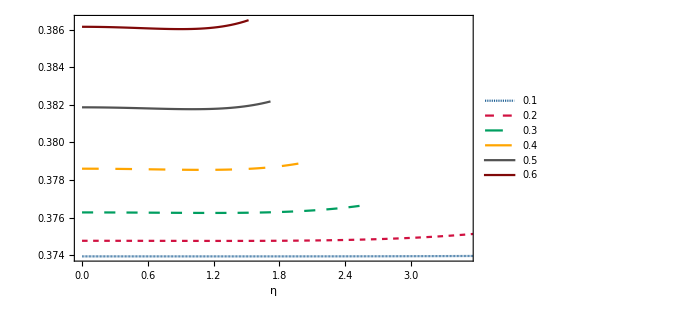

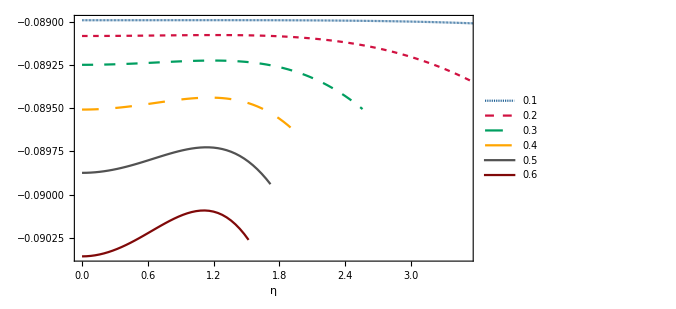

```mathematica
ListLinePlot[{Re[Ta[[1]]],Re[Ta[[2]]],Re[Ta[[3]]],Re[Ta[[4]]],Re[Ta[[5]]],Re[Ta[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[Ta[[1]]],Im[Ta[[2]]],Im[Ta[[3]]],Im[Ta[[4]]],Im[Ta[[5]]],Im[Ta[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
Max[Abs[(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100],Abs[(Max[Re[Tda[[2]]]]-Min[Re[Tda[[2]]]])/Min[Re[Tda[[2]]]]*100],Abs[(Max[Re[Tda[[3]]]]-Min[Re[Tda[[3]]]])/Min[Re[Tda[[3]]]]*100],Abs[(Max[Re[Tda[[4]]]]-Min[Re[Tda[[4]]]])/Min[Re[Tda[[4]]]]*100],Abs[(Max[Re[Tda[[5]]]]-Min[Re[Tda[[5]]]])/Min[Re[Tda[[5]]]]*100],Abs[(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100]]
Max[Abs[(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100],Abs[(Max[Im[Tda[[2]]]]-Min[Im[Tda[[2]]]])/Min[Im[Tda[[2]]]]*100],Abs[(Max[Im[Tda[[3]]]]-Min[Im[Tda[[3]]]])/Min[Im[Tda[[3]]]]*100],Abs[(Max[Im[Tda[[4]]]]-Min[Im[Tda[[4]]]])/Min[Im[Tda[[4]]]]*100],Abs[(Max[Im[Tda[[5]]]]-Min[Im[Tda[[5]]]])/Min[Im[Tda[[5]]]]*100],Abs[(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100]]
```

0.1232

0.361229

#### Polar modes

```mathematica
Tp={{{0,0.373934411406527-0.08899127264640017 ⅈ},{1/25+ⅈ/25,0.3739344079027655-0.08899127162242336 ⅈ},{2/25+(2 ⅈ)/25,0.3739343973958501-0.08899126855507755 ⅈ},{3/25+(3 ⅈ)/25,0.37393437989892697-0.08899126345813525 ⅈ},{4/25+(4 ⅈ)/25,0.3739343554339008-0.08899125635454837 ⅈ},{1/5+ⅈ/5,0.37393432403144067-0.08899124727644717 ⅈ},{6/25+(6 ⅈ)/25,0.37393428573098075-0.08899123626514055 ⅈ},{7/25+(7 ⅈ)/25,0.37393424058072416-0.08899122337111343 ⅈ},{8/25+(8 ⅈ)/25,0.37393418863764527-0.08899120865402532 ⅈ},{9/25+(9 ⅈ)/25,0.3739341299674933-0.08899119218270785 ⅈ},{2/5+(2 ⅈ)/5,0.37393406464479684-0.08899117403516248 ⅈ},{11/25+(11 ⅈ)/25,0.3739339927528687-0.0889911542985562 ⅈ},{12/25+(12 ⅈ)/25,0.37393391438381035-0.08899113306922034 ⅈ},{13/25+(13 ⅈ)/25,0.37393382963851857-0.08899111045264495 ⅈ},{14/25+(14 ⅈ)/25,0.373933738626692-0.0889910865634744 ⅈ},{3/5+(3 ⅈ)/5,0.37393364146683733-0.08899106152550429 ⅈ},{16/25+(16 ⅈ)/25,0.37393353828627707-0.08899103547167646 ⅈ},{17/25+(17 ⅈ)/25,0.37393342922115796-0.08899100854407212 ⅈ},{18/25+(18 ⅈ)/25,0.37393331441645894-0.0889909808939075 ⅈ},{19/25+(19 ⅈ)/25,0.37393319402600095-0.08899095268152787 ⅈ},{4/5+(4 ⅈ)/5,0.3739330682124563-0.08899092407639998 ⅈ},{21/25+(21 ⅈ)/25,0.37393293714735837-0.08899089525710653 ⅈ},{22/25+(22 ⅈ)/25,0.37393280101111337-0.0889908664113379 ⅈ},{23/25+(23 ⅈ)/25,0.37393265999301084-0.08899083773588443 ⅈ},{24/25+(24 ⅈ)/25,0.3739325142912361-0.08899080943662924 ⅈ},{1+ⅈ,0.37393236411288183-0.08899078172853853 ⅈ},{26/25+(26 ⅈ)/25,0.37393220967396185-0.08899075483565416 ⅈ},{27/25+(27 ⅈ)/25,0.3739320511994237-0.08899072899108193 ⅈ},{28/25+(28 ⅈ)/25,0.37393188892316276-0.08899070443698401 ⅈ},{29/25+(29 ⅈ)/25,0.37393172308803757-0.08899068142456729 ⅈ},{6/5+(6 ⅈ)/5,0.3739315539458839-0.08899066021407305 ⅈ},{31/25+(31 ⅈ)/25,0.3739313817575303-0.08899064107476565 ⅈ},{32/25+(32 ⅈ)/25,0.37393120679281455-0.08899062428492012 ⅈ},{33/25+(33 ⅈ)/25,0.3739310293305996-0.08899061013181189 ⅈ},{34/25+(34 ⅈ)/25,0.3739308496587915-0.08899059891170112 ⅈ},{7/5+(7 ⅈ)/5,0.3739306680743555-0.08899059092982306 ⅈ},{36/25+(36 ⅈ)/25,0.37393048488333597-0.08899058650037006 ⅈ},{37/25+(37 ⅈ)/25,0.3739303004008725-0.08899058594648165 ⅈ},{38/25+(38 ⅈ)/25,0.3739301149512213-0.08899058960022682 ⅈ},{39/25+(39 ⅈ)/25,0.3739299288677733-0.08899059780258899 ⅈ},{8/5+(8 ⅈ)/5,0.3739297424930741-0.08899061090345177 ⅈ},{41/25+(41 ⅈ)/25,0.37392955617884466-0.08899062926158001 ⅈ},{42/25+(42 ⅈ)/25,0.37392937028600304-0.08899065324460524 ⅈ},{43/25+(43 ⅈ)/25,0.3739291851846835-0.08899068322900637 ⅈ},{44/25+(44 ⅈ)/25,0.3739290012542606-0.08899071960009149 ⅈ},{9/5+(9 ⅈ)/5,0.3739288188833702-0.0889907627519803 ⅈ},{46/25+(46 ⅈ)/25,0.37392863846993274-0.08899081308758283 ⅈ},{47/25+(47 ⅈ)/25,0.37392846042117583-0.08899087101858025 ⅈ},{48/25+(48 ⅈ)/25,0.3739282851536579-0.0889909369654046 ⅈ},{49/25+(49 ⅈ)/25,0.3739281130932928-0.08899101135721645 ⅈ},{2+2 ⅈ,0.37392794467537327-0.08899109463188194 ⅈ},{51/25+(51 ⅈ)/25,0.3739277803445961-0.08899118723595278 ⅈ},{52/25+(52 ⅈ)/25,0.37392762055508755-0.08899128962463933 ⅈ},{53/25+(53 ⅈ)/25,0.37392746577042857-0.08899140226178869 ⅈ},{54/25+(54 ⅈ)/25,0.37392731646368116-0.08899152561985832 ⅈ},{11/5+(11 ⅈ)/5,0.37392717311741347-0.08899166017989124 ⅈ},{56/25+(56 ⅈ)/25,0.3739270362237287-0.08899180643148856 ⅈ},{57/25+(57 ⅈ)/25,0.37392690628428965-0.088991964872783 ⅈ},{58/25+(58 ⅈ)/25,0.373926783810348-0.08899213601040998 ⅈ},{59/25+(59 ⅈ)/25,0.37392666932277024-0.08899232035947953 ⅈ},{12/5+(12 ⅈ)/5,0.37392656335206764-0.08899251844354529 ⅈ},{61/25+(61 ⅈ)/25,0.37392646643842314-0.08899273079457516 ⅈ},{62/25+(62 ⅈ)/25,0.3739263791317202-0.08899295795291945 ⅈ},{63/25+(63 ⅈ)/25,0.37392630199157195-0.08899320046727718 ⅈ},{64/25+(64 ⅈ)/25,0.3739262355873503-0.08899345889466495 ⅈ},{13/5+(13 ⅈ)/5,0.3739261804982148-0.08899373380038143 ⅈ},{66/25+(66 ⅈ)/25,0.3739261373131434-0.08899402575797188 ⅈ},{67/25+(67 ⅈ)/25,0.37392610663096093-0.08899433534919357 ⅈ},{68/25+(68 ⅈ)/25,0.3739260890603704-0.08899466316397708 ⅈ},{69/25+(69 ⅈ)/25,0.3739260852199825-0.08899500980038941 ⅈ},{14/5+(14 ⅈ)/5,0.37392609573834606-0.08899537586459405 ⅈ},{71/25+(71 ⅈ)/25,0.3739261212539793-0.0889957619708117 ⅈ},{72/25+(72 ⅈ)/25,0.3739261624153998-0.08899616874127873 ⅈ},{73/25+(73 ⅈ)/25,0.37392621988115593-0.08899659680620488 ⅈ},{74/25+(74 ⅈ)/25,0.3739262943198575-0.08899704680373029 ⅈ},{3+3 ⅈ,0.37392638641020703-0.08899751937988082 ⅈ},{76/25+(76 ⅈ)/25,0.3739264968410311-0.08899801518852303 ⅈ},{77/25+(77 ⅈ)/25,0.37392662631131063-0.08899853489131694 ⅈ},{78/25+(78 ⅈ)/25,0.37392677553021375-0.08899907915766872 ⅈ},{79/25+(79 ⅈ)/25,0.3739269452171252-0.08899964866468181 ⅈ},{16/5+(16 ⅈ)/5,0.373927136101679-0.08900024409710591 ⅈ},{81/25+(81 ⅈ)/25,0.37392734892378865-0.08900086614728657 ⅈ},{82/25+(82 ⅈ)/25,0.3739275844336789-0.08900151551511251 ⅈ},{83/25+(83 ⅈ)/25,0.3739278433919165-0.08900219290796076 ⅈ},{84/25+(84 ⅈ)/25,0.37392812656944113-0.08900289904064297 ⅈ},{17/5+(17 ⅈ)/5,0.3739284347475963-0.0890036346353477 ⅈ},{86/25+(86 ⅈ)/25,0.37392876871815983-0.08900440042158295 ⅈ},{87/25+(87 ⅈ)/25,0.37392912928337446-0.08900519713611832 ⅈ},{88/25+(88 ⅈ)/25,0.37392951725597795-0.0890060255229219 ⅈ},{89/25+(89 ⅈ)/25,0.3739299334592327-0.08900688633310173 ⅈ},{18/5+(18 ⅈ)/5,0.3739303787269565-0.08900778032483987 ⅈ},{91/25+(91 ⅈ)/25,0.37393085390355035-0.08900870826332886 ⅈ},{92/25+(92 ⅈ)/25,0.3739313598440289-0.0890096709207062 ⅈ},{93/25+(93 ⅈ)/25,0.3739318974140483-0.08901066907598587 ⅈ},{94/25+(94 ⅈ)/25,0.37393246748993425-0.0890117035149897 ⅈ},{19/5+(19 ⅈ)/5,0.37393307095871087-0.08901277503027662 ⅈ},{96/25+(96 ⅈ)/25,0.37393370871812637-0.089013884421072 ⅈ},{97/25+(97 ⅈ)/25,0.3739343816766815-0.08901503249319173 ⅈ},{98/25+(98 ⅈ)/25,0.37393509075365433-0.08901622005896977 ⅈ},{99/25+(99 ⅈ)/25,0.37393583687912696-0.08901744793717929 ⅈ},{4+4 ⅈ,0.3739366209940097-0.08901871695295613 ⅈ},{101/25+(101 ⅈ)/25,0.3739374440500656-0.08902002793771815 ⅈ},{102/25+(102 ⅈ)/25,0.3739383070099342-0.08902138172908386 ⅈ},{103/25+(103 ⅈ)/25,0.37393921084715404-0.08902277917079 ⅈ},{104/25+(104 ⅈ)/25,0.37394015654618457-0.08902422111260605 ⅈ},{21/5+(21 ⅈ)/5,0.3739411451024276-0.08902570841024829 ⅈ},{106/25+(106 ⅈ)/25,0.373942177522247-0.08902724192529146 ⅈ},{107/25+(107 ⅈ)/25,0.3739432548229883-0.08902882252507978 ⅈ},{108/25+(108 ⅈ)/25,0.3739443780329965-0.08903045108263473 ⅈ},{109/25+(109 ⅈ)/25,0.3739455481916335-0.0890321284765625 ⅈ},{22/5+(22 ⅈ)/5,0.37394676634929414-0.08903385559095867 ⅈ},{111/25+(111 ⅈ)/25,0.37394803356742046-0.08903563331531193 ⅈ},{112/25+(112 ⅈ)/25,0.3739493509185158-0.08903746254440534 ⅈ},{113/25+(113 ⅈ)/25,0.37395071948615666-0.08903934417821714 ⅈ},{114/25+(114 ⅈ)/25,0.373952140365005-0.08904127912181731 ⅈ},{23/5+(23 ⅈ)/5,0.3739536146608151-0.08904326828526539 ⅈ},{116/25+(116 ⅈ)/25,0.37395514349044406-0.08904531258350461 ⅈ},{117/25+(117 ⅈ)/25,0.3739567279818574-0.08904741293625389 ⅈ},{118/25+(118 ⅈ)/25,0.37395836927413323-0.0890495702678995 ⅈ},{119/25+(119 ⅈ)/25,0.3739600685174666-0.08905178550738493 ⅈ},{24/5+(24 ⅈ)/5,0.37396182687317026-0.08905405958809655 ⅈ},{121/25+(121 ⅈ)/25,0.3739636455136743-0.0890563934477503 ⅈ},{122/25+(122 ⅈ)/25,0.3739655256225242-0.08905878802827528 ⅈ},{123/25+(123 ⅈ)/25,0.37396746839437656-0.08906124427569537 ⅈ},{124/25+(124 ⅈ)/25,0.373969475034992-0.0890637631400103 ⅈ},{5+5 ⅈ,0.3739715467612279-0.0890663455750727 ⅈ},{126/25+(126 ⅈ)/25,0.373973684801027-0.08906899253846509 ⅈ},{127/25+(127 ⅈ)/25,0.37397589039340456-0.08907170499137597 ⅈ},{128/25+(128 ⅈ)/25,0.3739781647884333-0.08907448389847049 ⅈ},{129/25+(129 ⅈ)/25,0.3739805092472253-0.08907733022776382 ⅈ},{26/5+(26 ⅈ)/5,0.37398292504191255-0.089080244950489 ⅈ},{131/25+(131 ⅈ)/25,0.3739854134556225-0.08908322904096622 ⅈ},{132/25+(132 ⅈ)/25,0.3739879757824535-0.08908628347646845 ⅈ},{133/25+(133 ⅈ)/25,0.37399061332744604-0.08908940923708401 ⅈ},{134/25+(134 ⅈ)/25,0.373993327406551-0.08909260730558263 ⅈ},{27/5+(27 ⅈ)/5,0.3739961193465957-0.08909587866727332 ⅈ},{136/25+(136 ⅈ)/25,0.37399899048524543-0.08909922430986594 ⅈ},{137/25+(137 ⅈ)/25,0.37400194217096344-0.08910264522332773 ⅈ},{138/25+(138 ⅈ)/25,0.37400497576296665-0.08910614239974061 ⅈ},{139/25+(139 ⅈ)/25,0.37400809263117746-0.08910971683315522 ⅈ},{28/5+(28 ⅈ)/5,0.3740112941561729-0.08911336951944474 ⅈ},{141/25+(141 ⅈ)/25,0.37401458172912994-0.08911710145615598 ⅈ},{142/25+(142 ⅈ)/25,0.3740179567517668-0.0891209136423609 ⅈ},{143/25+(143 ⅈ)/25,0.37402142063628-0.08912480707850504 ⅈ},{144/25+(144 ⅈ)/25,0.37402497480527824-0.08912878276625541 ⅈ},{29/5+(29 ⅈ)/5,0.37402862069171156-0.08913284170834677 ⅈ},{146/25+(146 ⅈ)/25,0.37403235973879667-0.08913698490842895 ⅈ},{147/25+(147 ⅈ)/25,0.3740361933999368-0.08914121337090755 ⅈ},{148/25+(148 ⅈ)/25,0.3740401231386384-0.08914552810079115 ⅈ},{149/25+(149 ⅈ)/25,0.37404415042842293-0.0891499301035306 ⅈ},{6+6 ⅈ,0.37404827675273244-0.0891544203848621 ⅈ},{151/25+(151 ⅈ)/25,0.37405250360483266-0.08915899995064709 ⅈ},{152/25+(152 ⅈ)/25,0.37405683248770905-0.08916366980671195 ⅈ},{153/25+(153 ⅈ)/25,0.3740612649139572-0.08916843095868843 ⅈ},{154/25+(154 ⅈ)/25,0.37406580240567144-0.08917328441185039 ⅈ},{31/5+(31 ⅈ)/5,0.3740704464943233-0.08917823117095355 ⅈ},{156/25+(156 ⅈ)/25,0.37407519872063766-0.0891832722400729 ⅈ},{157/25+(157 ⅈ)/25,0.3740800606344615-0.08918840862244014 ⅈ},{158/25+(158 ⅈ)/25,0.374085033794627-0.08919364132028153 ⅈ},{159/25+(159 ⅈ)/25,0.37409011976880996-0.08919897133465568 ⅈ},{32/5+(32 ⅈ)/5,0.3740953201333788-0.08920439966529106 ⅈ},{161/25+(161 ⅈ)/25,0.37410063647324066-0.08920992731042372 ⅈ},{162/25+(162 ⅈ)/25,0.374106070381679-0.08921555526663677 ⅈ},{163/25+(163 ⅈ)/25,0.3741116234601837-0.08922128452869779 ⅈ},{164/25+(164 ⅈ)/25,0.37411729731827686-0.0892271160894013 ⅈ},{33/5+(33 ⅈ)/5,0.37412309357332907-0.08923305093940677 ⅈ},{166/25+(166 ⅈ)/25,0.37412901385037006-0.08923909006708215 ⅈ},{167/25+(167 ⅈ)/25,0.37413505978189016-0.08924523445834645 ⅈ},{168/25+(168 ⅈ)/25,0.37414123300763635-0.08925148509651462 ⅈ},{169/25+(169 ⅈ)/25,0.3741475351743985-0.08925784296214405 ⅈ},{34/5+(34 ⅈ)/5,0.3741539679357894-0.0892643090328814 ⅈ},{171/25+(171 ⅈ)/25,0.3741605329520147-0.08927088428331499 ⅈ},{172/25+(172 ⅈ)/25,0.37416723188963763-0.0892775696848258 ⅈ},{173/25+(173 ⅈ)/25,0.3741740664213302-0.08928436620544296 ⅈ},{174/25+(174 ⅈ)/25,0.374181038225622-0.08929127480970263 ⅈ},{7+7 ⅈ,0.3741881489866341-0.08929829645850862 ⅈ},{176/25+(176 ⅈ)/25,0.3741954003938083-0.08930543210899607 ⅈ},{177/25+(177 ⅈ)/25,0.374202794141625-0.08931268271440033 ⅈ},{178/25+(178 ⅈ)/25,0.3742103319293117-0.08932004922392936 ⅈ}},{{0,0.37477384731613855-0.08908629925356583 ⅈ},{1/25+ⅈ/25,0.37477379669270977-0.0890862836173914 ⅈ},{2/25+(2 ⅈ)/25,0.37477364487515613-0.08908623678190523 ⅈ},{3/25+(3 ⅈ)/25,0.37477339202218696-0.089086158966373 ⅈ},{4/25+(4 ⅈ)/25,0.3747730383982532-0.08908605053619116 ⅈ},{1/5+ⅈ/5,0.3747725843736258-0.08908591200287454 ⅈ},{6/25+(6 ⅈ)/25,0.37477203042443613-0.08908574402401527 ⅈ},{7/25+(7 ⅈ)/25,0.3747713771327265-0.08908554740323131 ⅈ},{8/25+(8 ⅈ)/25,0.3747706251865129-0.08908532309009974 ⅈ},{9/25+(9 ⅈ)/25,0.37476977537985673-0.08908507218008223 ⅈ},{2/5+(2 ⅈ)/5,0.37476882861294764-0.08908479591443344 ⅈ},{11/25+(11 ⅈ)/25,0.37476778589219745-0.08908449568009941 ⅈ},{12/25+(12 ⅈ)/25,0.3747666483303412-0.0890841730096014 ⅈ},{13/25+(13 ⅈ)/25,0.37476541714654943-0.08908382958090481 ⅈ},{14/25+(14 ⅈ)/25,0.37476409366654845-0.08908346721727665 ⅈ},{3/5+(3 ⅈ)/5,0.3747626793227473-0.08908308788712475 ⅈ},{16/25+(16 ⅈ)/25,0.37476117565437406-0.0890826937038237 ⅈ},{17/25+(17 ⅈ)/25,0.37475958430761747-0.08908228692552476 ⅈ},{18/25+(18 ⅈ)/25,0.374757907035775-0.08908186995494782 ⅈ},{19/25+(19 ⅈ)/25,0.37475614569940546-0.08908144533915614 ⅈ},{4/5+(4 ⅈ)/5,0.37475430226648604-0.08908101576931479 ⅈ},{21/25+(21 ⅈ)/25,0.37475237881257295-0.08908058408042784 ⅈ},{22/25+(22 ⅈ)/25,0.37475037752096296-0.08908015325105716 ⅈ},{23/25+(23 ⅈ)/25,0.3747483006828572-0.08907972640302064 ⅈ},{24/25+(24 ⅈ)/25,0.37474615069752326-0.08907930680106904 ⅈ},{1+ⅈ,0.37474393007245793-0.08907889785253978 ⅈ},{26/25+(26 ⅈ)/25,0.3747416414235433-0.08907850310698943 ⅈ},{27/25+(27 ⅈ)/25,0.37473928747520524-0.08907812625580021 ⅈ},{28/25+(28 ⅈ)/25,0.3747368710605543-0.08907777113176238 ⅈ},{29/25+(29 ⅈ)/25,0.37473439512153217-0.0890774417086313 ⅈ},{6/5+(6 ⅈ)/5,0.3747318627090392-0.08907714210065565 ⅈ},{31/25+(31 ⅈ)/25,0.3747292769830536-0.0890768765620809 ⅈ},{32/25+(32 ⅈ)/25,0.37472664121273735-0.08907664948662032 ⅈ},{33/25+(33 ⅈ)/25,0.37472395877652603-0.08907646540689856 ⅈ},{34/25+(34 ⅈ)/25,0.3747212331622-0.08907632899386488 ⅈ},{7/5+(7 ⅈ)/5,0.37471846796693564-0.08907624505617139 ⅈ},{36/25+(36 ⅈ)/25,0.3747156668973343-0.08907621853952324 ⅈ},{37/25+(37 ⅈ)/25,0.37471283376942244-0.08907625452599174 ⅈ},{38/25+(38 ⅈ)/25,0.3747099725086277-0.0890763582332944 ⅈ},{39/25+(39 ⅈ)/25,0.3747070871497186-0.08907653501403927 ⅈ},{8/5+(8 ⅈ)/5,0.37470418183671184-0.0890767903549358 ⅈ},{41/25+(41 ⅈ)/25,0.3747012608227402-0.08907712987596418 ⅈ},{42/25+(42 ⅈ)/25,0.3746983284698789-0.08907755932951197 ⅈ},{43/25+(43 ⅈ)/25,0.37469538924892437-0.08907808459947224 ⅈ},{44/25+(44 ⅈ)/25,0.37469244773912574-0.08907871170029939 ⅈ},{9/5+(9 ⅈ)/5,0.37468950862786-0.08907944677603317 ⅈ},{46/25+(46 ⅈ)/25,0.3746865767102496-0.08908029609927746 ⅈ},{47/25+(47 ⅈ)/25,0.37468365688871547-0.08908126607014437 ⅈ},{48/25+(48 ⅈ)/25,0.3746807541724643-0.08908236321515822 ⅈ},{49/25+(49 ⅈ)/25,0.37467787367690053-0.08908359418612065 ⅈ},{2+2 ⅈ,0.37467502062295927-0.08908496575893826 ⅈ},{51/25+(51 ⅈ)/25,0.37467220033635684-0.08908648483241252 ⅈ},{52/25+(52 ⅈ)/25,0.37466941824675-0.08908815842699278 ⅈ},{53/25+(53 ⅈ)/25,0.3746666798867984-0.08908999368349545 ⅈ},{54/25+(54 ⅈ)/25,0.37466399089112407-0.08909199786178659 ⅈ},{11/5+(11 ⅈ)/5,0.37466135699516334-0.08909417833943412 ⅈ},{56/25+(56 ⅈ)/25,0.37465878403389846-0.0890965426103291 ⅈ},{57/25+(57 ⅈ)/25,0.3746562779404693-0.0890990982832789 ⅈ},{58/25+(58 ⅈ)/25,0.3746538447446514-0.08910185308057478 ⅈ},{59/25+(59 ⅈ)/25,0.374651490571194-0.08910481483653884 ⅈ},{12/5+(12 ⅈ)/5,0.37464922163801234-0.08910799149605082 ⅈ},{61/25+(61 ⅈ)/25,0.3746470442542228-0.08911139111306153 ⅈ},{62/25+(62 ⅈ)/25,0.37464496481801385-0.08911502184909564 ⅈ},{63/25+(63 ⅈ)/25,0.37464298981434174-0.08911889197175207 ⅈ},{64/25+(64 ⅈ)/25,0.37464112581244524-0.08912300985320223 ⅈ},{13/5+(13 ⅈ)/5,0.37463937946316483-0.0891273839686988 ⅈ},{66/25+(66 ⅈ)/25,0.37463775749606154-0.08913202289509745 ⅈ},{67/25+(67 ⅈ)/25,0.374636266716321-0.08913693530940243 ⅈ},{68/25+(68 ⅈ)/25,0.3746349140014347-0.08914212998734182 ⅈ},{69/25+(69 ⅈ)/25,0.37463370629764803-0.08914761580198487 ⅈ},{14/5+(14 ⅈ)/5,0.3746326506161616-0.08915340172240961 ⅈ},{71/25+(71 ⅈ)/25,0.37463175402907856-0.08915949681243265 ⅈ},{72/25+(72 ⅈ)/25,0.3746310236650832-0.08916591022941395 ⅈ},{73/25+(73 ⅈ)/25,0.3746304667048424-0.0891726512231494 ⅈ},{74/25+(74 ⅈ)/25,0.374630090376116-0.08917972913486645 ⅈ},{3+3 ⅈ,0.37462990194856605-0.08918715339633716 ⅈ},{76/25+(76 ⅈ)/25,0.37462990872825486-0.08919493352912629 ⅈ},{77/25+(77 ⅈ)/25,0.3746301180518166-0.0892030791439946 ⅈ},{78/25+(78 ⅈ)/25,0.3746305372802948-0.08921159994047276 ⅈ},{79/25+(79 ⅈ)/25,0.3746311737926336-0.08922050570663201 ⅈ},{16/5+(16 ⅈ)/5,0.37463203497881115-0.0892298063190692 ⅈ},{81/25+(81 ⅈ)/25,0.37463312823260564-0.0892395117431358 ⅈ},{82/25+(82 ⅈ)/25,0.3746344609439839-0.08924963203343078 ⅈ},{83/25+(83 ⅈ)/25,0.3746360404911021-0.08926017733459234 ⅈ},{84/25+(84 ⅈ)/25,0.37463787423191314-0.08927115788240862 ⅈ},{17/5+(17 ⅈ)/5,0.3746399694953677-0.08928258400528874 ⅈ},{86/25+(86 ⅈ)/25,0.3746423335722063-0.0892944661261174 ⅈ},{87/25+(87 ⅈ)/25,0.37464497370533456-0.08930681476453813 ⅈ},{88/25+(88 ⅈ)/25,0.374647897079778-0.08931964053969277 ⅈ},{89/25+(89 ⅈ)/25,0.3746511108122121-0.08933295417346203 ⅈ},{18/5+(18 ⅈ)/5,0.3746546219400673-0.08934676649424783 ⅈ},{91/25+(91 ⅈ)/25,0.3746584374102086-0.08936108844133742 ⅈ}},{{0,0.37632202480439797-0.08926895190367796 ⅈ},{1/25+ⅈ/25,0.3763218064473809-0.08926887812295008 ⅈ},{2/25+(2 ⅈ)/25,0.3763211515464739-0.08926865714901479 ⅈ},{3/25+(3 ⅈ)/25,0.3763200606142624-0.08926829008737681 ⅈ},{4/25+(4 ⅈ)/25,0.3763185345045836-0.0892677787804996 ⅈ},{1/5+ⅈ/5,0.37631657441258115-0.08926712580799688 ⅈ},{6/25+(6 ⅈ)/25,0.37631418187447346-0.08926633448679368 ⅈ},{7/25+(7 ⅈ)/25,0.37631135876724775-0.08926540887133565 ⅈ},{8/25+(8 ⅈ)/25,0.3763081073082804-0.08926435375383597 ⅈ},{9/25+(9 ⅈ)/25,0.3763044300548713-0.08926317466456848 ⅈ},{2/5+(2 ⅈ)/5,0.37630032990369155-0.08926187787219507 ⅈ},{11/25+(11 ⅈ)/25,0.3762958100901345-0.0892604703841322 ⅈ},{12/25+(12 ⅈ)/25,0.3762908741875605-0.08925895994694998 ⅈ},{13/25+(13 ⅈ)/25,0.3762855261064252-0.08925735504680486 ⅈ},{14/25+(14 ⅈ)/25,0.3762797700932836-0.08925566490989614 ⅈ},{3/5+(3 ⅈ)/5,0.37627361072965326-0.08925389950295468 ⅈ},{16/25+(16 ⅈ)/25,0.37626705293072443-0.08925206953375085 ⅈ},{17/25+(17 ⅈ)/25,0.3762601019439037-0.08925018645162656 ⅈ},{18/25+(18 ⅈ)/25,0.37625276334717134-0.08924826244804522 ⅈ},{19/25+(19 ⅈ)/25,0.3762450430472384-0.08924631045716308 ⅈ},{4/5+(4 ⅈ)/5,0.37623694727748014-0.08924434415641408 ⅈ},{21/25+(21 ⅈ)/25,0.37622848259562885-0.0892423779671175 ⅈ},{22/25+(22 ⅈ)/25,0.3762196558812004-0.08924042705510098 ⅈ},{23/25+(23 ⅈ)/25,0.3762104743326324-0.08923850733134608 ⅈ},{24/25+(24 ⅈ)/25,0.3762009454641083-0.08923663545265964 ⅈ},{1+ⅈ,0.37619107710203853-0.08923482882237387 ⅈ},{26/25+(26 ⅈ)/25,0.37618087738117234-0.0892331055910849 ⅈ},{27/25+(27 ⅈ)/25,0.3761703547403065-0.08923148465743537 ⅈ},{28/25+(28 ⅈ)/25,0.3761595179175644-0.089229985668962 ⅈ},{29/25+(29 ⅈ)/25,0.3761483759452032-0.08922862902300492 ⅈ},{6/5+(6 ⅈ)/5,0.37613693814392213-0.08922743586771807 ⅈ},{31/25+(31 ⅈ)/25,0.3761252141166324-0.08922642810318396 ⅈ},{32/25+(32 ⅈ)/25,0.3761132137416487-0.08922562838266739 ⅈ},{33/25+(33 ⅈ)/25,0.37610094716526754-0.08922506011403586 ⅈ},{34/25+(34 ⅈ)/25,0.3760884247936898-0.08922474746137651 ⅈ},{7/5+(7 ⅈ)/5,0.37607565728424996-0.08922471534685694 ⅈ},{36/25+(36 ⅈ)/25,0.37606265553590884-0.08922498945286754 ⅈ},{37/25+(37 ⅈ)/25,0.37604943067897345-0.0892255962245003 ⅈ},{38/25+(38 ⅈ)/25,0.37603599406400223-0.08922656287242411 ⅈ},{39/25+(39 ⅈ)/25,0.3760223572498601-0.08922791737622059 ⅈ},{8/5+(8 ⅈ)/5,0.3760085319908851-0.08922968848825413 ⅈ},{41/25+(41 ⅈ)/25,0.37599453022313906-0.08923190573816034 ⅈ},{42/25+(42 ⅈ)/25,0.3759803640497081-0.08923459943804435 ⅈ},{43/25+(43 ⅈ)/25,0.37596604572503545-0.08923780068849008 ⅈ},{44/25+(44 ⅈ)/25,0.3759515876382653-0.08924154138549288 ⅈ},{9/5+(9 ⅈ)/5,0.37593700229559285-0.08924585422843798 ⅈ},{46/25+(46 ⅈ)/25,0.3759223023016186-0.08925077272925824 ⅈ},{47/25+(47 ⅈ)/25,0.3759075003397226-0.089256331222916 ⅈ},{48/25+(48 ⅈ)/25,0.37589260915148154-0.08926256487936572 ⅈ},{49/25+(49 ⅈ)/25,0.37587764151517505-0.08926950971716412 ⅈ},{2+2 ⅈ,0.37586261022344064-0.08927720261890736 ⅈ},{51/25+(51 ⅈ)/25,0.37584752806016164-0.08928568134868409 ⅈ},{52/25+(52 ⅈ)/25,0.37583240777669663-0.08929498457174313 ⅈ},{53/25+(53 ⅈ)/25,0.37581726206758764-0.08930515187658178 ⅈ},{54/25+(54 ⅈ)/25,0.3758021035459172-0.08931622379967127 ⅈ},{11/5+(11 ⅈ)/5,0.3757869447185212-0.08932824185303304 ⅈ},{56/25+(56 ⅈ)/25,0.3757717979613049-0.08934124855488859 ⅈ},{57/25+(57 ⅈ)/25,0.3757566754949552-0.08935528746359904 ⅈ},{58/25+(58 ⅈ)/25,0.3757415893613943-0.08937040321510108 ⅈ},{59/25+(59 ⅈ)/25,0.37572655140137295-0.08938664156404069 ⅈ},{12/5+(12 ⅈ)/5,0.3757115732336641-0.08940404942878118 ⅈ},{61/25+(61 ⅈ)/25,0.3756966662363817-0.08942267494043517 ⅈ},{62/25+(62 ⅈ)/25,0.3756818415310201-0.08944256749603631 ⅈ},{63/25+(63 ⅈ)/25,0.37566710996988306-0.08946377781591916 ⅈ},{64/25+(64 ⅈ)/25,0.3756524821276531-0.0894863580053137 ⅈ}},{{0,0.37874264140427905-0.08956743603738573 ⅈ},{1/25+ⅈ/25,0.3787420810719928-0.089567222285057 ⅈ},{2/25+(2 ⅈ)/25,0.3787404003730566-0.08956658218536573 ⅈ},{3/25+(3 ⅈ)/25,0.378737600206559-0.08956551921298128 ⅈ},{4/25+(4 ⅈ)/25,0.37873368206909824-0.08956403916080906 ⅈ},{1/5+ⅈ/5,0.3787286480539173-0.08956215014343706 ⅈ},{6/25+(6 ⅈ)/25,0.3787225008489024-0.08955986260166034 ⅈ},{7/25+(7 ⅈ)/25,0.37871524373399984-0.08955718930832461 ⅈ},{8/25+(8 ⅈ)/25,0.3787068805780438-0.08955414537548853 ⅈ},{9/25+(9 ⅈ)/25,0.37869741583498834-0.08955074826293305 ⅈ},{2/5+(2 ⅈ)/5,0.3786868545395333-0.08954701778802863 ⅈ},{11/25+(11 ⅈ)/25,0.378675202302134-0.08954297613700263 ⅈ},{12/25+(12 ⅈ)/25,0.37866246530339037-0.0895386478776238 ⅈ},{13/25+(13 ⅈ)/25,0.37864865028779915-0.08953405997335612 ⅈ},{14/25+(14 ⅈ)/25,0.37863376455686937-0.08952924179902498 ⅈ},{3/5+(3 ⅈ)/5,0.37861781596159244-0.08952422515805515 ⅈ},{16/25+(16 ⅈ)/25,0.37860081289426606-0.08951904430134487 ⅈ},{17/25+(17 ⅈ)/25,0.3785827642796779-0.08951373594786234 ⅈ},{18/25+(18 ⅈ)/25,0.3785636795656552-0.08950833930705104 ⅈ},{19/25+(19 ⅈ)/25,0.3785435687130037-0.08950289610315681 ⅈ},{4/5+(4 ⅈ)/5,0.3785224421848647-0.08949745060159914 ⅈ},{21/25+(21 ⅈ)/25,0.37850031093553177-0.08949204963753345 ⅈ},{22/25+(22 ⅈ)/25,0.3784771863987925-0.08948674264676637 ⅈ},{23/25+(23 ⅈ)/25,0.3784530804758765-0.089481581699212 ⅈ},{24/25+(24 ⅈ)/25,0.37842800552312333-0.08947662153510258 ⅈ},{1+ⅈ,0.37840197433949324-0.08947191960418471 ⅈ},{26/25+(26 ⅈ)/25,0.37837500015414766-0.08946753610818008 ⅈ},{27/25+(27 ⅈ)/25,0.3783470966142668-0.08946353404678929 ⅈ},{28/25+(28 ⅈ)/25,0.37831827777343024-0.08945997926757045 ⅈ},{29/25+(29 ⅈ)/25,0.378288558080894-0.08945694052004886 ⅈ},{6/5+(6 ⅈ)/5,0.37825795237219106-0.0894544895144336 ⅈ},{31/25+(31 ⅈ)/25,0.37822647586157165-0.08945270098535602 ⅈ},{32/25+(32 ⅈ)/25,0.3781941441369083-0.08945165276105925 ⅈ},{33/25+(33 ⅈ)/25,0.378160973157809-0.0894514258384916 ⅈ},{34/25+(34 ⅈ)/25,0.3781269792578271-0.08945210446476227 ⅈ},{7/5+(7 ⅈ)/5,0.37809217915181553-0.08945377622542126 ⅈ},{36/25+(36 ⅈ)/25,0.37805658994966-0.08945653214000548 ⅈ},{37/25+(37 ⅈ)/25,0.37802022917783445-0.08946046676526373 ⅈ},{38/25+(38 ⅈ)/25,0.3779831148104537-0.08946567830640892 ⅈ},{39/25+(39 ⅈ)/25,0.3779452653117635-0.08947226873666222 ⅈ},{8/5+(8 ⅈ)/5,0.3779066996922888-0.08948034392522403 ⅈ},{41/25+(41 ⅈ)/25,0.37786743758118196-0.08949001377363464 ⅈ},{42/25+(42 ⅈ)/25,0.37782749931764226-0.08950139236025939 ⅈ},{43/25+(43 ⅈ)/25,0.3777869060646411-0.08951459809233682 ⅈ},{44/25+(44 ⅈ)/25,0.37774567994855207-0.08952975386465992 ⅈ},{9/5+(9 ⅈ)/5,0.3777038442286699-0.08954698722348813 ⅈ},{46/25+(46 ⅈ)/25,0.37766142350096554-0.08956643053372934 ⅈ},{47/25+(47 ⅈ)/25,0.37761844394077976-0.089588221146742 ⅈ},{48/25+(48 ⅈ)/25,0.37757493358945887-0.08961250156528922 ⅈ},{49/25+(49 ⅈ)/25,0.37753092269018285-0.08963941960123058 ⅈ},{2+2 ⅈ,0.3774864440783642-0.08966912852042061 ⅈ}},{{0,0.3821844608663658-0.09000968928947416 ⅈ},{1/25+ⅈ/25,0.3821833942805746-0.09000921643410494 ⅈ},{2/25+(2 ⅈ)/25,0.38218019489801763-0.09000780065320246 ⅈ},{3/25+(3 ⅈ)/25,0.38217486385342775-0.09000545031112936 ⅈ},{4/25+(4 ⅈ)/25,0.3821674030349927-0.09000217936109615 ⅈ},{1/5+ⅈ/5,0.38215781508360375-0.08999800736579391 ⅈ},{6/25+(6 ⅈ)/25,0.38214610339045585-0.08999295952574035 ⅈ},{7/25+(7 ⅈ)/25,0.38213227209420497-0.08998706671594636 ⅈ},{8/25+(8 ⅈ)/25,0.382116326077882-0.08998036553107151 ⅈ},{9/25+(9 ⅈ)/25,0.38209827096580834-0.08997289833927756 ⅈ},{2/5+(2 ⅈ)/5,0.38207811312082207-0.08996471334504152 ⅈ},{11/25+(11 ⅈ)/25,0.38205585964220007-0.08995586466123273 ⅈ},{12/25+(12 ⅈ)/25,0.38203151836471744-0.0899464123907938 ⅈ},{13/25+(13 ⅈ)/25,0.38200509785942927-0.08993642271848008 ⅈ},{14/25+(14 ⅈ)/25,0.3819766074368001-0.0899259680130763 ⅈ},{3/5+(3 ⅈ)/5,0.38194605715299296-0.08991512694065548 ⅈ},{16/25+(16 ⅈ)/25,0.3819134578202489-0.08990398458946798 ⅈ},{17/25+(17 ⅈ)/25,0.3818788210224717-0.0898926326071202 ⅈ},{18/25+(18 ⅈ)/25,0.3818421591373319-0.08988116935077237 ⅈ},{19/25+(19 ⅈ)/25,0.38180348536645503-0.08986970005114214 ⅈ},{4/5+(4 ⅈ)/5,0.3817628137755272-0.08985833699116244 ⅈ},{21/25+(21 ⅈ)/25,0.38172015934649106-0.08984719970018287 ⅈ},{22/25+(22 ⅈ)/25,0.3816755380443757-0.0898364151646369 ⅈ},{23/25+(23 ⅈ)/25,0.381628966901758-0.08982611805610025 ⅈ},{24/25+(24 ⅈ)/25,0.38158046412435165-0.08981645097763671 ⅈ},{1+ⅈ,0.3815300492218171-0.08980756472925198 ⅈ},{26/25+(26 ⅈ)/25,0.38147774316855-0.08979961859313507 ⅈ},{27/25+(27 ⅈ)/25,0.3814235685999657-0.08979278063914164 ⅈ},{28/25+(28 ⅈ)/25,0.3813675500506525-0.08978722805064984 ⅈ},{29/25+(29 ⅈ)/25,0.3813097142417208-0.08978314747043854 ⅈ},{6/5+(6 ⅈ)/5,0.3812500904257125-0.08978073536561286 ⅈ},{31/25+(31 ⅈ)/25,0.3811887107985772-0.08978019840972966 ⅈ},{32/25+(32 ⅈ)/25,0.38112561098942416-0.0897817538791738 ⅈ},{33/25+(33 ⅈ)/25,0.38106083064000906-0.08978563005938907 ⅈ},{34/25+(34 ⅈ)/25,0.3809944140871732-0.089792066654765 ⅈ},{7/5+(7 ⅈ)/5,0.3809264111626544-0.08980131519372046 ⅈ},{36/25+(36 ⅈ)/25,0.380856878125761-0.08981363941777061 ⅈ},{37/25+(37 ⅈ)/25,0.38078587874522235-0.0898293156400252 ⅈ},{38/25+(38 ⅈ)/25,0.3807134855469711-0.08984863305461338 ⅈ},{39/25+(39 ⅈ)/25,0.3806397812444943-0.08987189397390756 ⅈ},{8/5+(8 ⅈ)/5,0.3805648603674818-0.0898994139651323 ⅈ},{41/25+(41 ⅈ)/25,0.38048883110255083-0.08993152185202442 ⅈ},{42/25+(42 ⅈ)/25,0.3804118173565413-0.08996855954076137 ⅈ},{43/25+(43 ⅈ)/25,0.38033396104789674-0.09001088162258772 ⅈ}},{{0,0.38675397649681126-0.09061844336301762 ⅈ},{1/25+ⅈ/25,0.3867523154197056-0.09061756283780689 ⅈ},{2/25+(2 ⅈ)/25,0.3867473326445666-0.09061492686458132 ⅈ},{3/25+(3 ⅈ)/25,0.3867390295582066-0.0906105522741955 ⅈ},{4/25+(4 ⅈ)/25,0.386727408474922-0.09060446716610213 ⅈ},{1/5+ⅈ/5,0.38671247264725717-0.09059671098378452 ⅈ},{6/25+(6 ⅈ)/25,0.38669422627982414-0.09058733461974951 ⅈ},{7/25+(7 ⅈ)/25,0.38667267454896276-0.09057640055158467 ⅈ},{8/25+(8 ⅈ)/25,0.38664782362970995-0.09056398300986054 ⅈ},{9/25+(9 ⅈ)/25,0.38661968073199104-0.09055016817891649 ⅈ},{2/5+(2 ⅈ)/5,0.3865882541483566-0.09053505443163755 ⅈ},{11/25+(11 ⅈ)/25,0.386553553316148-0.09051875259961686 ⅈ},{12/25+(12 ⅈ)/25,0.38651558889754656-0.09050138628021544 ⅈ},{13/25+(13 ⅈ)/25,0.38647437288165803-0.09048309218221039 ⅈ},{14/25+(14 ⅈ)/25,0.3864299187135696-0.09046402051186125 ⅈ},{3/5+(3 ⅈ)/5,0.38638224145624117-0.0904443354013308 ⅈ},{16/25+(16 ⅈ)/25,0.38633135799215695-0.09042421538144989 ⅈ},{17/25+(17 ⅈ)/25,0.38627728727290156-0.0904038539007924 ⅈ},{18/25+(18 ⅈ)/25,0.3862200506262533-0.09038345989289917 ⅈ},{19/25+(19 ⅈ)/25,0.38615967213203556-0.090363258393212 ⅈ},{4/5+(4 ⅈ)/5,0.3860961790798612-0.09034349120680178 ⅈ},{21/25+(21 ⅈ)/25,0.3860296025240526-0.09032441762723464 ⅈ},{22/25+(22 ⅈ)/25,0.38595997795345593-0.0903063152058204 ⅈ},{23/25+(23 ⅈ)/25,0.38588734609658304-0.09028948056895696 ⅈ},{24/25+(24 ⅈ)/25,0.3858117538855092-0.09027423027913749 ⅈ},{1+ⅈ,0.3857332556051844-0.09026090173235457 ⅈ},{26/25+(26 ⅈ)/25,0.38565191425823775-0.09024985408085039 ⅈ},{27/25+(27 ⅈ)/25,0.3855678031788301-0.09024146916528594 ⅈ},{28/25+(28 ⅈ)/25,0.3854810079324883-0.09023615243416974 ⅈ},{29/25+(29 ⅈ)/25,0.38539162854186715-0.09023433382055104 ⅈ},{6/5+(6 ⅈ)/5,0.38529978208067756-0.09023646853631255 ⅈ},{31/25+(31 ⅈ)/25,0.3852056056791026-0.09024303773262772 ⅈ},{32/25+(32 ⅈ)/25,0.3851092599832355-0.09025454896113377 ⅈ},{33/25+(33 ⅈ)/25,0.38501093310761103-0.09027153635401819 ⅈ},{34/25+(34 ⅈ)/25,0.38491084511271606-0.09029456042263569 ⅈ},{7/5+(7 ⅈ)/5,0.3848092530272598-0.09032420735383663 ⅈ},{36/25+(36 ⅈ)/25,0.38470645641656626-0.0903610876616637 ⅈ},{37/25+(37 ⅈ)/25,0.3846028034722615-0.09040583403071732 ⅈ},{38/25+(38 ⅈ)/25,0.38449869756304295-0.09045909816826316 ⅈ}}};
```

```mathematica
Tdp={{{0.373934411406527-0.08899127264640017 ⅈ},{0.3739344079027655-0.08899127162242336 ⅈ},{0.3739343973958501-0.08899126855507755 ⅈ},{0.37393437989892697-0.08899126345813525 ⅈ},{0.3739343554339008-0.08899125635454837 ⅈ},{0.37393432403144067-0.08899124727644717 ⅈ},{0.37393428573098075-0.08899123626514055 ⅈ},{0.37393424058072416-0.08899122337111343 ⅈ},{0.37393418863764527-0.08899120865402532 ⅈ},{0.3739341299674933-0.08899119218270785 ⅈ},{0.37393406464479684-0.08899117403516248 ⅈ},{0.3739339927528687-0.0889911542985562 ⅈ},{0.37393391438381035-0.08899113306922034 ⅈ},{0.37393382963851857-0.08899111045264495 ⅈ},{0.373933738626692-0.0889910865634744 ⅈ},{0.37393364146683733-0.08899106152550429 ⅈ},{0.37393353828627707-0.08899103547167646 ⅈ},{0.37393342922115796-0.08899100854407212 ⅈ},{0.37393331441645894-0.0889909808939075 ⅈ},{0.37393319402600095-0.08899095268152787 ⅈ},{0.3739330682124563-0.08899092407639998 ⅈ},{0.37393293714735837-0.08899089525710653 ⅈ},{0.37393280101111337-0.0889908664113379 ⅈ},{0.37393265999301084-0.08899083773588443 ⅈ},{0.3739325142912361-0.08899080943662924 ⅈ},{0.37393236411288183-0.08899078172853853 ⅈ},{0.37393220967396185-0.08899075483565416 ⅈ},{0.3739320511994237-0.08899072899108193 ⅈ},{0.37393188892316276-0.08899070443698401 ⅈ},{0.37393172308803757-0.08899068142456729 ⅈ},{0.3739315539458839-0.08899066021407305 ⅈ},{0.3739313817575303-0.08899064107476565 ⅈ},{0.37393120679281455-0.08899062428492012 ⅈ},{0.3739310293305996-0.08899061013181189 ⅈ},{0.3739308496587915-0.08899059891170112 ⅈ},{0.3739306680743555-0.08899059092982306 ⅈ},{0.37393048488333597-0.08899058650037006 ⅈ},{0.3739303004008725-0.08899058594648165 ⅈ},{0.3739301149512213-0.08899058960022682 ⅈ},{0.3739299288677733-0.08899059780258899 ⅈ},{0.3739297424930741-0.08899061090345177 ⅈ},{0.37392955617884466-0.08899062926158001 ⅈ},{0.37392937028600304-0.08899065324460524 ⅈ},{0.3739291851846835-0.08899068322900637 ⅈ},{0.3739290012542606-0.08899071960009149 ⅈ},{0.3739288188833702-0.0889907627519803 ⅈ},{0.37392863846993274-0.08899081308758283 ⅈ},{0.37392846042117583-0.08899087101858025 ⅈ},{0.3739282851536579-0.0889909369654046 ⅈ},{0.3739281130932928-0.08899101135721645 ⅈ},{0.37392794467537327-0.08899109463188194 ⅈ},{0.3739277803445961-0.08899118723595278 ⅈ},{0.37392762055508755-0.08899128962463933 ⅈ},{0.37392746577042857-0.08899140226178869 ⅈ},{0.37392731646368116-0.08899152561985832 ⅈ},{0.37392717311741347-0.08899166017989124 ⅈ},{0.3739270362237287-0.08899180643148856 ⅈ},{0.37392690628428965-0.088991964872783 ⅈ},{0.373926783810348-0.08899213601040998 ⅈ},{0.37392666932277024-0.08899232035947953 ⅈ},{0.37392656335206764-0.08899251844354529 ⅈ},{0.37392646643842314-0.08899273079457516 ⅈ},{0.3739263791317202-0.08899295795291945 ⅈ},{0.37392630199157195-0.08899320046727718 ⅈ},{0.3739262355873503-0.08899345889466495 ⅈ},{0.3739261804982148-0.08899373380038143 ⅈ},{0.3739261373131434-0.08899402575797188 ⅈ},{0.37392610663096093-0.08899433534919357 ⅈ},{0.3739260890603704-0.08899466316397708 ⅈ},{0.3739260852199825-0.08899500980038941 ⅈ},{0.37392609573834606-0.08899537586459405 ⅈ},{0.3739261212539793-0.0889957619708117 ⅈ},{0.3739261624153998-0.08899616874127873 ⅈ},{0.37392621988115593-0.08899659680620488 ⅈ},{0.3739262943198575-0.08899704680373029 ⅈ},{0.37392638641020703-0.08899751937988082 ⅈ},{0.3739264968410311-0.08899801518852303 ⅈ},{0.37392662631131063-0.08899853489131694 ⅈ},{0.37392677553021375-0.08899907915766872 ⅈ},{0.3739269452171252-0.08899964866468181 ⅈ},{0.373927136101679-0.08900024409710591 ⅈ},{0.37392734892378865-0.08900086614728657 ⅈ},{0.3739275844336789-0.08900151551511251 ⅈ},{0.3739278433919165-0.08900219290796076 ⅈ},{0.37392812656944113-0.08900289904064297 ⅈ},{0.3739284347475963-0.0890036346353477 ⅈ},{0.37392876871815983-0.08900440042158295 ⅈ},{0.37392912928337446-0.08900519713611832 ⅈ},{0.37392951725597795-0.0890060255229219 ⅈ},{0.3739299334592327-0.08900688633310173 ⅈ},{0.3739303787269565-0.08900778032483987 ⅈ},{0.37393085390355035-0.08900870826332886 ⅈ},{0.3739313598440289-0.0890096709207062 ⅈ},{0.3739318974140483-0.08901066907598587 ⅈ},{0.37393246748993425-0.0890117035149897 ⅈ},{0.37393307095871087-0.08901277503027662 ⅈ},{0.37393370871812637-0.089013884421072 ⅈ},{0.3739343816766815-0.08901503249319173 ⅈ},{0.37393509075365433-0.08901622005896977 ⅈ},{0.37393583687912696-0.08901744793717929 ⅈ},{0.3739366209940097-0.08901871695295613 ⅈ},{0.3739374440500656-0.08902002793771815 ⅈ},{0.3739383070099342-0.08902138172908386 ⅈ},{0.37393921084715404-0.08902277917079 ⅈ},{0.37394015654618457-0.08902422111260605 ⅈ},{0.3739411451024276-0.08902570841024829 ⅈ},{0.373942177522247-0.08902724192529146 ⅈ},{0.3739432548229883-0.08902882252507978 ⅈ},{0.3739443780329965-0.08903045108263473 ⅈ},{0.3739455481916335-0.0890321284765625 ⅈ},{0.37394676634929414-0.08903385559095867 ⅈ},{0.37394803356742046-0.08903563331531193 ⅈ},{0.3739493509185158-0.08903746254440534 ⅈ},{0.37395071948615666-0.08903934417821714 ⅈ},{0.373952140365005-0.08904127912181731 ⅈ},{0.3739536146608151-0.08904326828526539 ⅈ},{0.37395514349044406-0.08904531258350461 ⅈ},{0.3739567279818574-0.08904741293625389 ⅈ},{0.37395836927413323-0.0890495702678995 ⅈ},{0.3739600685174666-0.08905178550738493 ⅈ},{0.37396182687317026-0.08905405958809655 ⅈ},{0.3739636455136743-0.0890563934477503 ⅈ},{0.3739655256225242-0.08905878802827528 ⅈ},{0.37396746839437656-0.08906124427569537 ⅈ},{0.373969475034992-0.0890637631400103 ⅈ},{0.3739715467612279-0.0890663455750727 ⅈ},{0.373973684801027-0.08906899253846509 ⅈ},{0.37397589039340456-0.08907170499137597 ⅈ},{0.3739781647884333-0.08907448389847049 ⅈ},{0.3739805092472253-0.08907733022776382 ⅈ},{0.37398292504191255-0.089080244950489 ⅈ},{0.3739854134556225-0.08908322904096622 ⅈ},{0.3739879757824535-0.08908628347646845 ⅈ},{0.37399061332744604-0.08908940923708401 ⅈ},{0.373993327406551-0.08909260730558263 ⅈ},{0.3739961193465957-0.08909587866727332 ⅈ},{0.37399899048524543-0.08909922430986594 ⅈ},{0.37400194217096344-0.08910264522332773 ⅈ},{0.37400497576296665-0.08910614239974061 ⅈ},{0.37400809263117746-0.08910971683315522 ⅈ},{0.3740112941561729-0.08911336951944474 ⅈ},{0.37401458172912994-0.08911710145615598 ⅈ},{0.3740179567517668-0.0891209136423609 ⅈ},{0.37402142063628-0.08912480707850504 ⅈ},{0.37402497480527824-0.08912878276625541 ⅈ},{0.37402862069171156-0.08913284170834677 ⅈ},{0.37403235973879667-0.08913698490842895 ⅈ},{0.3740361933999368-0.08914121337090755 ⅈ},{0.3740401231386384-0.08914552810079115 ⅈ},{0.37404415042842293-0.0891499301035306 ⅈ},{0.37404827675273244-0.0891544203848621 ⅈ},{0.37405250360483266-0.08915899995064709 ⅈ},{0.37405683248770905-0.08916366980671195 ⅈ},{0.3740612649139572-0.08916843095868843 ⅈ},{0.37406580240567144-0.08917328441185039 ⅈ},{0.3740704464943233-0.08917823117095355 ⅈ},{0.37407519872063766-0.0891832722400729 ⅈ},{0.3740800606344615-0.08918840862244014 ⅈ},{0.374085033794627-0.08919364132028153 ⅈ},{0.37409011976880996-0.08919897133465568 ⅈ},{0.3740953201333788-0.08920439966529106 ⅈ},{0.37410063647324066-0.08920992731042372 ⅈ},{0.374106070381679-0.08921555526663677 ⅈ},{0.3741116234601837-0.08922128452869779 ⅈ},{0.37411729731827686-0.0892271160894013 ⅈ},{0.37412309357332907-0.08923305093940677 ⅈ},{0.37412901385037006-0.08923909006708215 ⅈ},{0.37413505978189016-0.08924523445834645 ⅈ},{0.37414123300763635-0.08925148509651462 ⅈ},{0.3741475351743985-0.08925784296214405 ⅈ},{0.3741539679357894-0.0892643090328814 ⅈ},{0.3741605329520147-0.08927088428331499 ⅈ},{0.37416723188963763-0.0892775696848258 ⅈ},{0.3741740664213302-0.08928436620544296 ⅈ},{0.374181038225622-0.08929127480970263 ⅈ},{0.3741881489866341-0.08929829645850862 ⅈ},{0.3741954003938083-0.08930543210899607 ⅈ},{0.374202794141625-0.08931268271440033 ⅈ},{0.3742103319293117-0.08932004922392936 ⅈ}},{{0.37477384731613855-0.08908629925356583 ⅈ},{0.37477379669270977-0.0890862836173914 ⅈ},{0.37477364487515613-0.08908623678190523 ⅈ},{0.37477339202218696-0.089086158966373 ⅈ},{0.3747730383982532-0.08908605053619116 ⅈ},{0.3747725843736258-0.08908591200287454 ⅈ},{0.37477203042443613-0.08908574402401527 ⅈ},{0.3747713771327265-0.08908554740323131 ⅈ},{0.3747706251865129-0.08908532309009974 ⅈ},{0.37476977537985673-0.08908507218008223 ⅈ},{0.37476882861294764-0.08908479591443344 ⅈ},{0.37476778589219745-0.08908449568009941 ⅈ},{0.3747666483303412-0.0890841730096014 ⅈ},{0.37476541714654943-0.08908382958090481 ⅈ},{0.37476409366654845-0.08908346721727665 ⅈ},{0.3747626793227473-0.08908308788712475 ⅈ},{0.37476117565437406-0.0890826937038237 ⅈ},{0.37475958430761747-0.08908228692552476 ⅈ},{0.374757907035775-0.08908186995494782 ⅈ},{0.37475614569940546-0.08908144533915614 ⅈ},{0.37475430226648604-0.08908101576931479 ⅈ},{0.37475237881257295-0.08908058408042784 ⅈ},{0.37475037752096296-0.08908015325105716 ⅈ},{0.3747483006828572-0.08907972640302064 ⅈ},{0.37474615069752326-0.08907930680106904 ⅈ},{0.37474393007245793-0.08907889785253978 ⅈ},{0.3747416414235433-0.08907850310698943 ⅈ},{0.37473928747520524-0.08907812625580021 ⅈ},{0.3747368710605543-0.08907777113176238 ⅈ},{0.37473439512153217-0.0890774417086313 ⅈ},{0.3747318627090392-0.08907714210065565 ⅈ},{0.3747292769830536-0.0890768765620809 ⅈ},{0.37472664121273735-0.08907664948662032 ⅈ},{0.37472395877652603-0.08907646540689856 ⅈ},{0.3747212331622-0.08907632899386488 ⅈ},{0.37471846796693564-0.08907624505617139 ⅈ},{0.3747156668973343-0.08907621853952324 ⅈ},{0.37471283376942244-0.08907625452599174 ⅈ},{0.3747099725086277-0.0890763582332944 ⅈ},{0.3747070871497186-0.08907653501403927 ⅈ},{0.37470418183671184-0.0890767903549358 ⅈ},{0.3747012608227402-0.08907712987596418 ⅈ},{0.3746983284698789-0.08907755932951197 ⅈ},{0.37469538924892437-0.08907808459947224 ⅈ},{0.37469244773912574-0.08907871170029939 ⅈ},{0.37468950862786-0.08907944677603317 ⅈ},{0.3746865767102496-0.08908029609927746 ⅈ},{0.37468365688871547-0.08908126607014437 ⅈ},{0.3746807541724643-0.08908236321515822 ⅈ},{0.37467787367690053-0.08908359418612065 ⅈ},{0.37467502062295927-0.08908496575893826 ⅈ},{0.37467220033635684-0.08908648483241252 ⅈ},{0.37466941824675-0.08908815842699278 ⅈ},{0.3746666798867984-0.08908999368349545 ⅈ},{0.37466399089112407-0.08909199786178659 ⅈ},{0.37466135699516334-0.08909417833943412 ⅈ},{0.37465878403389846-0.0890965426103291 ⅈ},{0.3746562779404693-0.0890990982832789 ⅈ},{0.3746538447446514-0.08910185308057478 ⅈ},{0.374651490571194-0.08910481483653884 ⅈ},{0.37464922163801234-0.08910799149605082 ⅈ},{0.3746470442542228-0.08911139111306153 ⅈ},{0.37464496481801385-0.08911502184909564 ⅈ},{0.37464298981434174-0.08911889197175207 ⅈ},{0.37464112581244524-0.08912300985320223 ⅈ},{0.37463937946316483-0.0891273839686988 ⅈ},{0.37463775749606154-0.08913202289509745 ⅈ},{0.374636266716321-0.08913693530940243 ⅈ},{0.3746349140014347-0.08914212998734182 ⅈ},{0.37463370629764803-0.08914761580198487 ⅈ},{0.3746326506161616-0.08915340172240961 ⅈ},{0.37463175402907856-0.08915949681243265 ⅈ},{0.3746310236650832-0.08916591022941395 ⅈ},{0.3746304667048424-0.0891726512231494 ⅈ},{0.374630090376116-0.08917972913486645 ⅈ},{0.37462990194856605-0.08918715339633716 ⅈ},{0.37462990872825486-0.08919493352912629 ⅈ},{0.3746301180518166-0.0892030791439946 ⅈ},{0.3746305372802948-0.08921159994047276 ⅈ},{0.3746311737926336-0.08922050570663201 ⅈ},{0.37463203497881115-0.0892298063190692 ⅈ},{0.37463312823260564-0.0892395117431358 ⅈ},{0.3746344609439839-0.08924963203343078 ⅈ},{0.3746360404911021-0.08926017733459234 ⅈ},{0.37463787423191314-0.08927115788240862 ⅈ},{0.3746399694953677-0.08928258400528874 ⅈ},{0.3746423335722063-0.0892944661261174 ⅈ},{0.37464497370533456-0.08930681476453813 ⅈ},{0.374647897079778-0.08931964053969277 ⅈ},{0.3746511108122121-0.08933295417346203 ⅈ},{0.3746546219400673-0.08934676649424783 ⅈ},{0.3746584374102086-0.08936108844133742 ⅈ}},{{0.37632202480439797-0.08926895190367796 ⅈ},{0.3763218064473809-0.08926887812295008 ⅈ},{0.3763211515464739-0.08926865714901479 ⅈ},{0.3763200606142624-0.08926829008737681 ⅈ},{0.3763185345045836-0.0892677787804996 ⅈ},{0.37631657441258115-0.08926712580799688 ⅈ},{0.37631418187447346-0.08926633448679368 ⅈ},{0.37631135876724775-0.08926540887133565 ⅈ},{0.3763081073082804-0.08926435375383597 ⅈ},{0.3763044300548713-0.08926317466456848 ⅈ},{0.37630032990369155-0.08926187787219507 ⅈ},{0.3762958100901345-0.0892604703841322 ⅈ},{0.3762908741875605-0.08925895994694998 ⅈ},{0.3762855261064252-0.08925735504680486 ⅈ},{0.3762797700932836-0.08925566490989614 ⅈ},{0.37627361072965326-0.08925389950295468 ⅈ},{0.37626705293072443-0.08925206953375085 ⅈ},{0.3762601019439037-0.08925018645162656 ⅈ},{0.37625276334717134-0.08924826244804522 ⅈ},{0.3762450430472384-0.08924631045716308 ⅈ},{0.37623694727748014-0.08924434415641408 ⅈ},{0.37622848259562885-0.0892423779671175 ⅈ},{0.3762196558812004-0.08924042705510098 ⅈ},{0.3762104743326324-0.08923850733134608 ⅈ},{0.3762009454641083-0.08923663545265964 ⅈ},{0.37619107710203853-0.08923482882237387 ⅈ},{0.37618087738117234-0.0892331055910849 ⅈ},{0.3761703547403065-0.08923148465743537 ⅈ},{0.3761595179175644-0.089229985668962 ⅈ},{0.3761483759452032-0.08922862902300492 ⅈ},{0.37613693814392213-0.08922743586771807 ⅈ},{0.3761252141166324-0.08922642810318396 ⅈ},{0.3761132137416487-0.08922562838266739 ⅈ},{0.37610094716526754-0.08922506011403586 ⅈ},{0.3760884247936898-0.08922474746137651 ⅈ},{0.37607565728424996-0.08922471534685694 ⅈ},{0.37606265553590884-0.08922498945286754 ⅈ},{0.37604943067897345-0.0892255962245003 ⅈ},{0.37603599406400223-0.08922656287242411 ⅈ},{0.3760223572498601-0.08922791737622059 ⅈ},{0.3760085319908851-0.08922968848825413 ⅈ},{0.37599453022313906-0.08923190573816034 ⅈ},{0.3759803640497081-0.08923459943804435 ⅈ},{0.37596604572503545-0.08923780068849008 ⅈ},{0.3759515876382653-0.08924154138549288 ⅈ},{0.37593700229559285-0.08924585422843798 ⅈ},{0.3759223023016186-0.08925077272925824 ⅈ},{0.3759075003397226-0.089256331222916 ⅈ},{0.37589260915148154-0.08926256487936572 ⅈ},{0.37587764151517505-0.08926950971716412 ⅈ},{0.37586261022344064-0.08927720261890736 ⅈ},{0.37584752806016164-0.08928568134868409 ⅈ},{0.37583240777669663-0.08929498457174313 ⅈ},{0.37581726206758764-0.08930515187658178 ⅈ},{0.3758021035459172-0.08931622379967127 ⅈ},{0.3757869447185212-0.08932824185303304 ⅈ},{0.3757717979613049-0.08934124855488859 ⅈ},{0.3757566754949552-0.08935528746359904 ⅈ},{0.3757415893613943-0.08937040321510108 ⅈ},{0.37572655140137295-0.08938664156404069 ⅈ},{0.3757115732336641-0.08940404942878118 ⅈ},{0.3756966662363817-0.08942267494043517 ⅈ},{0.3756818415310201-0.08944256749603631 ⅈ},{0.37566710996988306-0.08946377781591916 ⅈ},{0.3756524821276531-0.0894863580053137 ⅈ}},{{0.37874264140427905-0.08956743603738573 ⅈ},{0.3787420810719928-0.089567222285057 ⅈ},{0.3787404003730566-0.08956658218536573 ⅈ},{0.378737600206559-0.08956551921298128 ⅈ},{0.37873368206909824-0.08956403916080906 ⅈ},{0.3787286480539173-0.08956215014343706 ⅈ},{0.3787225008489024-0.08955986260166034 ⅈ},{0.37871524373399984-0.08955718930832461 ⅈ},{0.3787068805780438-0.08955414537548853 ⅈ},{0.37869741583498834-0.08955074826293305 ⅈ},{0.3786868545395333-0.08954701778802863 ⅈ},{0.378675202302134-0.08954297613700263 ⅈ},{0.37866246530339037-0.0895386478776238 ⅈ},{0.37864865028779915-0.08953405997335612 ⅈ},{0.37863376455686937-0.08952924179902498 ⅈ},{0.37861781596159244-0.08952422515805515 ⅈ},{0.37860081289426606-0.08951904430134487 ⅈ},{0.3785827642796779-0.08951373594786234 ⅈ},{0.3785636795656552-0.08950833930705104 ⅈ},{0.3785435687130037-0.08950289610315681 ⅈ},{0.3785224421848647-0.08949745060159914 ⅈ},{0.37850031093553177-0.08949204963753345 ⅈ},{0.3784771863987925-0.08948674264676637 ⅈ},{0.3784530804758765-0.089481581699212 ⅈ},{0.37842800552312333-0.08947662153510258 ⅈ},{0.37840197433949324-0.08947191960418471 ⅈ},{0.37837500015414766-0.08946753610818008 ⅈ},{0.3783470966142668-0.08946353404678929 ⅈ},{0.37831827777343024-0.08945997926757045 ⅈ},{0.378288558080894-0.08945694052004886 ⅈ},{0.37825795237219106-0.0894544895144336 ⅈ},{0.37822647586157165-0.08945270098535602 ⅈ},{0.3781941441369083-0.08945165276105925 ⅈ},{0.378160973157809-0.0894514258384916 ⅈ},{0.3781269792578271-0.08945210446476227 ⅈ},{0.37809217915181553-0.08945377622542126 ⅈ},{0.37805658994966-0.08945653214000548 ⅈ},{0.37802022917783445-0.08946046676526373 ⅈ},{0.3779831148104537-0.08946567830640892 ⅈ},{0.3779452653117635-0.08947226873666222 ⅈ},{0.3779066996922888-0.08948034392522403 ⅈ},{0.37786743758118196-0.08949001377363464 ⅈ},{0.37782749931764226-0.08950139236025939 ⅈ},{0.3777869060646411-0.08951459809233682 ⅈ},{0.37774567994855207-0.08952975386465992 ⅈ},{0.3777038442286699-0.08954698722348813 ⅈ},{0.37766142350096554-0.08956643053372934 ⅈ},{0.37761844394077976-0.089588221146742 ⅈ},{0.37757493358945887-0.08961250156528922 ⅈ},{0.37753092269018285-0.08963941960123058 ⅈ},{0.3774864440783642-0.08966912852042061 ⅈ}},{{0.3821844608663658-0.09000968928947416 ⅈ},{0.3821833942805746-0.09000921643410494 ⅈ},{0.38218019489801763-0.09000780065320246 ⅈ},{0.38217486385342775-0.09000545031112936 ⅈ},{0.3821674030349927-0.09000217936109615 ⅈ},{0.38215781508360375-0.08999800736579391 ⅈ},{0.38214610339045585-0.08999295952574035 ⅈ},{0.38213227209420497-0.08998706671594636 ⅈ},{0.382116326077882-0.08998036553107151 ⅈ},{0.38209827096580834-0.08997289833927756 ⅈ},{0.38207811312082207-0.08996471334504152 ⅈ},{0.38205585964220007-0.08995586466123273 ⅈ},{0.38203151836471744-0.0899464123907938 ⅈ},{0.38200509785942927-0.08993642271848008 ⅈ},{0.3819766074368001-0.0899259680130763 ⅈ},{0.38194605715299296-0.08991512694065548 ⅈ},{0.3819134578202489-0.08990398458946798 ⅈ},{0.3818788210224717-0.0898926326071202 ⅈ},{0.3818421591373319-0.08988116935077237 ⅈ},{0.38180348536645503-0.08986970005114214 ⅈ},{0.3817628137755272-0.08985833699116244 ⅈ},{0.38172015934649106-0.08984719970018287 ⅈ},{0.3816755380443757-0.0898364151646369 ⅈ},{0.381628966901758-0.08982611805610025 ⅈ},{0.38158046412435165-0.08981645097763671 ⅈ},{0.3815300492218171-0.08980756472925198 ⅈ},{0.38147774316855-0.08979961859313507 ⅈ},{0.3814235685999657-0.08979278063914164 ⅈ},{0.3813675500506525-0.08978722805064984 ⅈ},{0.3813097142417208-0.08978314747043854 ⅈ},{0.3812500904257125-0.08978073536561286 ⅈ},{0.3811887107985772-0.08978019840972966 ⅈ},{0.38112561098942416-0.0897817538791738 ⅈ},{0.38106083064000906-0.08978563005938907 ⅈ},{0.3809944140871732-0.089792066654765 ⅈ},{0.3809264111626544-0.08980131519372046 ⅈ},{0.380856878125761-0.08981363941777061 ⅈ},{0.38078587874522235-0.0898293156400252 ⅈ},{0.3807134855469711-0.08984863305461338 ⅈ},{0.3806397812444943-0.08987189397390756 ⅈ},{0.3805648603674818-0.0898994139651323 ⅈ},{0.38048883110255083-0.08993152185202442 ⅈ},{0.3804118173565413-0.08996855954076137 ⅈ},{0.38033396104789674-0.09001088162258772 ⅈ}},{{0.38675397649681126-0.09061844336301762 ⅈ},{0.3867523154197056-0.09061756283780689 ⅈ},{0.3867473326445666-0.09061492686458132 ⅈ},{0.3867390295582066-0.0906105522741955 ⅈ},{0.386727408474922-0.09060446716610213 ⅈ},{0.38671247264725717-0.09059671098378452 ⅈ},{0.38669422627982414-0.09058733461974951 ⅈ},{0.38667267454896276-0.09057640055158467 ⅈ},{0.38664782362970995-0.09056398300986054 ⅈ},{0.38661968073199104-0.09055016817891649 ⅈ},{0.3865882541483566-0.09053505443163755 ⅈ},{0.386553553316148-0.09051875259961686 ⅈ},{0.38651558889754656-0.09050138628021544 ⅈ},{0.38647437288165803-0.09048309218221039 ⅈ},{0.3864299187135696-0.09046402051186125 ⅈ},{0.38638224145624117-0.0904443354013308 ⅈ},{0.38633135799215695-0.09042421538144989 ⅈ},{0.38627728727290156-0.0904038539007924 ⅈ},{0.3862200506262533-0.09038345989289917 ⅈ},{0.38615967213203556-0.090363258393212 ⅈ},{0.3860961790798612-0.09034349120680178 ⅈ},{0.3860296025240526-0.09032441762723464 ⅈ},{0.38595997795345593-0.0903063152058204 ⅈ},{0.38588734609658304-0.09028948056895696 ⅈ},{0.3858117538855092-0.09027423027913749 ⅈ},{0.3857332556051844-0.09026090173235457 ⅈ},{0.38565191425823775-0.09024985408085039 ⅈ},{0.3855678031788301-0.09024146916528594 ⅈ},{0.3854810079324883-0.09023615243416974 ⅈ},{0.38539162854186715-0.09023433382055104 ⅈ},{0.38529978208067756-0.09023646853631255 ⅈ},{0.3852056056791026-0.09024303773262772 ⅈ},{0.3851092599832355-0.09025454896113377 ⅈ},{0.38501093310761103-0.09027153635401819 ⅈ},{0.38491084511271606-0.09029456042263569 ⅈ},{0.3848092530272598-0.09032420735383663 ⅈ},{0.38470645641656626-0.0903610876616637 ⅈ},{0.3846028034722615-0.09040583403071732 ⅈ},{0.38449869756304295-0.09045909816826316 ⅈ}}};
```

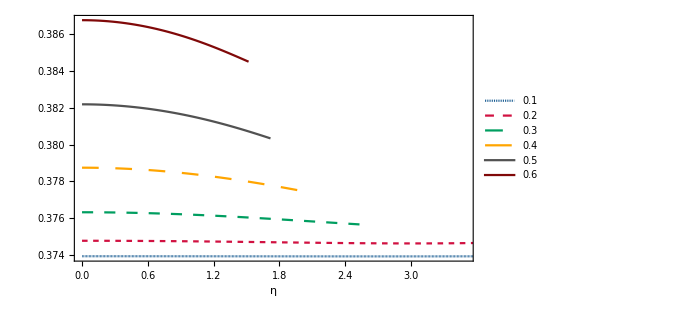

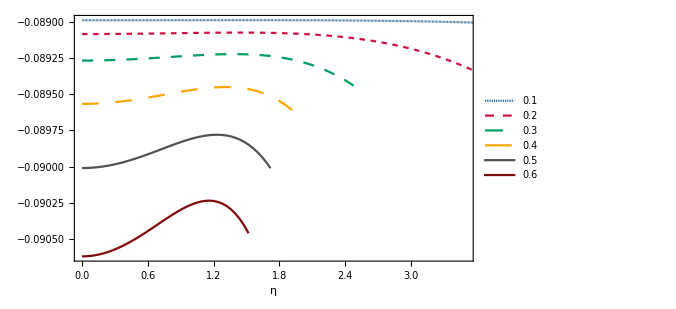

```mathematica
ListLinePlot[{Re[Tp[[1]]],Re[Tp[[2]]],Re[Tp[[3]]],Re[Tp[[4]]],Re[Tp[[5]]],Re[Tp[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[Tp[[1]]],Im[Tp[[2]]],Im[Tp[[3]]],Im[Tp[[4]]],Im[Tp[[5]]],Im[Tp[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
Max[Abs[(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100],Abs[(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100],Abs[(Max[Re[Tdp[[3]]]]-Min[Re[Tdp[[3]]]])/Min[Re[Tdp[[3]]]]*100],Abs[(Max[Re[Tdp[[4]]]]-Min[Re[Tdp[[4]]]])/Min[Re[Tdp[[4]]]]*100],Abs[(Max[Re[Tdp[[5]]]]-Min[Re[Tdp[[5]]]])/Min[Re[Tdp[[5]]]]*100],Abs[(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100],Abs[(Max[Im[Tdp[[2]]]]-Min[Im[Tdp[[2]]]])/Min[Im[Tdp[[2]]]]*100],Abs[(Max[Im[Tdp[[3]]]]-Min[Im[Tdp[[3]]]])/Min[Im[Tdp[[3]]]]*100],Abs[(Max[Im[Tdp[[4]]]]-Min[Im[Tdp[[4]]]])/Min[Im[Tdp[[4]]]]*100],Abs[(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100],Abs[(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100]]
```

0.58655

0.423876

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tdp]-Im[Tda])[[k]][[j+1]][[1]]/(Abs[Im[Tda][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

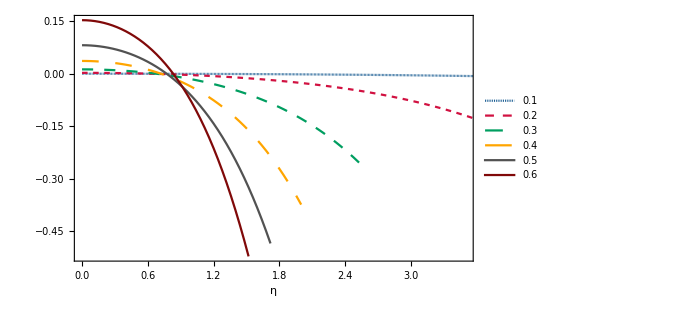

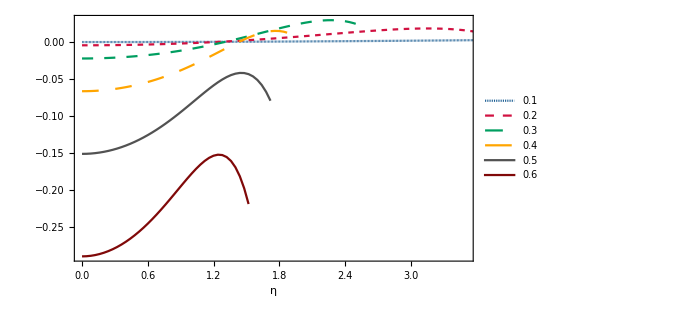

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
Max[Abs[(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100],Abs[(Max[Re[Tda[[2]]]]-Min[Re[Tda[[2]]]])/Min[Re[Tda[[2]]]]*100],Abs[(Max[Re[Tda[[3]]]]-Min[Re[Tda[[3]]]])/Min[Re[Tda[[3]]]]*100],Abs[(Max[Re[Tda[[4]]]]-Min[Re[Tda[[4]]]])/Min[Re[Tda[[4]]]]*100],Abs[(Max[Re[Tda[[5]]]]-Min[Re[Tda[[5]]]])/Min[Re[Tda[[5]]]]*100],Abs[(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100]]
Max[Abs[(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100],Abs[(Max[Im[Tda[[2]]]]-Min[Im[Tda[[2]]]])/Min[Im[Tda[[2]]]]*100],Abs[(Max[Im[Tda[[3]]]]-Min[Im[Tda[[3]]]])/Min[Im[Tda[[3]]]]*100],Abs[(Max[Im[Tda[[4]]]]-Min[Im[Tda[[4]]]])/Min[Im[Tda[[4]]]]*100],Abs[(Max[Im[Tda[[5]]]]-Min[Im[Tda[[5]]]])/Min[Im[Tda[[5]]]]*100],Abs[(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100]]
```

0.1232

0.361229

```mathematica
Max[Abs[(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100],Abs[(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100],Abs[(Max[Re[Tdp[[3]]]]-Min[Re[Tdp[[3]]]])/Min[Re[Tdp[[3]]]]*100],Abs[(Max[Re[Tdp[[4]]]]-Min[Re[Tdp[[4]]]])/Min[Re[Tdp[[4]]]]*100],Abs[(Max[Re[Tdp[[5]]]]-Min[Re[Tdp[[5]]]])/Min[Re[Tdp[[5]]]]*100],Abs[(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100],Abs[(Max[Im[Tdp[[2]]]]-Min[Im[Tdp[[2]]]])/Min[Im[Tdp[[2]]]]*100],Abs[(Max[Im[Tdp[[3]]]]-Min[Im[Tdp[[3]]]])/Min[Im[Tdp[[3]]]]*100],Abs[(Max[Im[Tdp[[4]]]]-Min[Im[Tdp[[4]]]])/Min[Im[Tdp[[4]]]]*100],Abs[(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100],Abs[(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100]]
```

0.58655

0.423876

## l=3 grav. mode axial & polar

#### Axial modes

```mathematica
Ta={{{0,0.5998190562224931-0.09272483427557163 ⅈ},{1/25+ⅈ/25,0.5998190545658683-0.09272483354861162 ⅈ},{2/25+(2 ⅈ)/25,0.5998190496066346-0.09272483137331716 ⅈ},{3/25+(3 ⅈ)/25,0.5998190413767309-0.09272482776644746 ⅈ},{4/25+(4 ⅈ)/25,0.5998190299293873-0.09272482275593188 ⅈ},{1/5+ⅈ/5,0.5998190153391308-0.09272481638087392 ⅈ},{6/25+(6 ⅈ)/25,0.5998189977017794-0.09272480869152619 ⅈ},{7/25+(7 ⅈ)/25,0.5998189771344568-0.09272479974931692 ⅈ},{8/25+(8 ⅈ)/25,0.5998189537755894-0.09272478962682568 ⅈ},{9/25+(9 ⅈ)/25,0.5998189277849127-0.09272477840778168 ⅈ},{2/5+(2 ⅈ)/5,0.5998188993434774-0.09272476618705665 ⅈ},{11/25+(11 ⅈ)/25,0.5998188686536543-0.09272475307065703 ⅈ},{12/25+(12 ⅈ)/25,0.599818835939142-0.09272473917571479 ⅈ},{13/25+(13 ⅈ)/25,0.5998188014449746-0.09272472463047766 ⅈ},{14/25+(14 ⅈ)/25,0.5998187654375294-0.09272470957429807 ⅈ},{3/5+(3 ⅈ)/5,0.5998187282045363-0.09272469415762147 ⅈ},{16/25+(16 ⅈ)/25,0.5998186900550879-0.09272467854197328 ⅈ},{17/25+(17 ⅈ)/25,0.5998186513196492-0.09272466289994516 ⅈ},{18/25+(18 ⅈ)/25,0.5998186123500685-0.09272464741518006 ⅈ},{19/25+(19 ⅈ)/25,0.5998185735195907-0.09272463228235657 ⅈ},{4/5+(4 ⅈ)/5,0.5998185352228678-0.09272461770717184 ⅈ},{21/25+(21 ⅈ)/25,0.5998184978759734-0.09272460390632362 ⅈ},{22/25+(22 ⅈ)/25,0.5998184619164161-0.0927245911074918 ⅈ},{23/25+(23 ⅈ)/25,0.5998184278031536-0.09272457954931779 ⅈ},{24/25+(24 ⅈ)/25,0.5998183960166087-0.09272456948138398 ⅈ},{1+ⅈ,0.599818367058684-0.0927245611641914 ⅈ},{26/25+(26 ⅈ)/25,0.5998183414527786-0.09272455486913667 ⅈ},{27/25+(27 ⅈ)/25,0.599818319743806-0.09272455087848755 ⅈ},{28/25+(28 ⅈ)/25,0.5998183024982103-0.09272454948535783 ⅈ},{29/25+(29 ⅈ)/25,0.5998182903039848-0.09272455099368332 ⅈ},{6/5+(6 ⅈ)/5,0.5998182837706957-0.09272455571818239 ⅈ},{31/25+(31 ⅈ)/25,0.5998182835294897-0.09272456398434553 ⅈ},{32/25+(32 ⅈ)/25,0.5998182902331247-0.0927245761283932 ⅈ},{33/25+(33 ⅈ)/25,0.5998183045559845-0.09272459249725597 ⅈ},{34/25+(34 ⅈ)/25,0.5998183271941113-0.09272461344851589 ⅈ},{7/5+(7 ⅈ)/5,0.5998183588652094-0.09272463935040458 ⅈ},{36/25+(36 ⅈ)/25,0.5998184003086794-0.09272467058175138 ⅈ},{37/25+(37 ⅈ)/25,0.5998184522856381-0.09272470753195076 ⅈ},{38/25+(38 ⅈ)/25,0.5998185155789411-0.09272475060092525 ⅈ},{39/25+(39 ⅈ)/25,0.5998185909932078-0.09272480019908645 ⅈ},{8/5+(8 ⅈ)/5,0.5998186793548437-0.09272485674729562 ⅈ},{41/25+(41 ⅈ)/25,0.5998187815120674-0.09272492067682193 ⅈ},{42/25+(42 ⅈ)/25,0.5998188983349331-0.09272499242930046 ⅈ},{43/25+(43 ⅈ)/25,0.5998190307153584-0.0927250724566878 ⅈ},{44/25+(44 ⅈ)/25,0.5998191795671486-0.09272516122121709 ⅈ},{9/5+(9 ⅈ)/5,0.599819345826024-0.09272525919535096 ⅈ},{46/25+(46 ⅈ)/25,0.5998195304496459-0.09272536686173359 ⅈ},{47/25+(47 ⅈ)/25,0.5998197344176441-0.09272548471314108 ⅈ},{48/25+(48 ⅈ)/25,0.5998199587316443-0.09272561325243023 ⅈ},{49/25+(49 ⅈ)/25,0.599820204415295-0.09272575299248616 ⅈ},{2+2 ⅈ,0.5998204725142972-0.09272590445616785 ⅈ},{51/25+(51 ⅈ)/25,0.5998207640964304-0.09272606817625288 ⅈ},{52/25+(52 ⅈ)/25,0.5998210802515832-0.09272624469537977 ⅈ},{53/25+(53 ⅈ)/25,0.5998214220917812-0.09272643456598946 ⅈ},{54/25+(54 ⅈ)/25,0.5998217907512158-0.09272663835026466 ⅈ},{11/5+(11 ⅈ)/5,0.5998221873862737-0.09272685662006783 ⅈ},{56/25+(56 ⅈ)/25,0.599822613175566-0.09272708995687724 ⅈ},{57/25+(57 ⅈ)/25,0.5998230693199583-0.09272733895172162 ⅈ},{58/25+(58 ⅈ)/25,0.5998235570425998-0.0927276042051128 ⅈ},{59/25+(59 ⅈ)/25,0.5998240775889532-0.0927278863269768 ⅈ},{12/5+(12 ⅈ)/5,0.599824632226824-0.09272818593658298 ⅈ},{61/25+(61 ⅈ)/25,0.5998252222463915-0.09272850366247154 ⅈ},{62/25+(62 ⅈ)/25,0.5998258489602369-0.09272884014237896 ⅈ},{63/25+(63 ⅈ)/25,0.5998265137033753-0.09272919602316185 ⅈ},{64/25+(64 ⅈ)/25,0.5998272178332834-0.09272957196071846 ⅈ},{13/5+(13 ⅈ)/5,0.5998279627299307-0.09272996861990891 ⅈ},{66/25+(66 ⅈ)/25,0.5998287497958081-0.09273038667447285 ⅈ},{67/25+(67 ⅈ)/25,0.5998295804559582-0.09273082680694542 ⅈ},{68/25+(68 ⅈ)/25,0.599830456158004-0.09273128970857118 ⅈ},{69/25+(69 ⅈ)/25,0.5998313783721784-0.09273177607921596 ⅈ},{14/5+(14 ⅈ)/5,0.5998323485913527-0.09273228662727659 ⅈ},{71/25+(71 ⅈ)/25,0.5998333683310658-0.09273282206958856 ⅈ},{72/25+(72 ⅈ)/25,0.5998344391295518-0.09273338313133159 ⅈ},{73/25+(73 ⅈ)/25,0.5998355625477684-0.09273397054593309 ⅈ},{74/25+(74 ⅈ)/25,0.5998367401694246-0.09273458505496893 ⅈ},{3+3 ⅈ,0.5998379736010077-0.09273522740806278 ⅈ},{76/25+(76 ⅈ)/25,0.5998392644718096-0.09273589836278265 ⅈ},{77/25+(77 ⅈ)/25,0.5998406144339542-0.09273659868453495 ⅈ},{78/25+(78 ⅈ)/25,0.5998420251624217-0.092737329146457 ⅈ},{79/25+(79 ⅈ)/25,0.5998434983550752-0.09273809052930636 ⅈ},{16/5+(16 ⅈ)/5,0.5998450357326838-0.09273888362134824 ⅈ},{81/25+(81 ⅈ)/25,0.5998466390389476-0.09273970921824039 ⅈ},{82/25+(82 ⅈ)/25,0.5998483100405203-0.09274056812291541 ⅈ},{83/25+(83 ⅈ)/25,0.5998500505270316-0.09274146114546078 ⅈ},{84/25+(84 ⅈ)/25,0.5998518623111093-0.09274238910299627 ⅈ},{17/5+(17 ⅈ)/5,0.5998537472283993-0.09274335281954889 ⅈ},{86/25+(86 ⅈ)/25,0.5998557071375868-0.09274435312592481 ⅈ},{87/25+(87 ⅈ)/25,0.5998577439204137-0.09274539085957959 ⅈ},{88/25+(88 ⅈ)/25,0.5998598594816978-0.0927464668644849 ⅈ},{89/25+(89 ⅈ)/25,0.5998620557493493-0.09274758199099292 ⅈ},{18/5+(18 ⅈ)/5,0.5998643346743864-0.09274873709569825 ⅈ},{91/25+(91 ⅈ)/25,0.5998666982309505-0.09274993304129654 ⅈ},{92/25+(92 ⅈ)/25,0.5998691484163197-0.09275117069644093 ⅈ},{93/25+(93 ⅈ)/25,0.5998716872509208-0.09275245093559543 ⅈ},{94/25+(94 ⅈ)/25,0.5998743167783402-0.09275377463888551 ⅈ},{19/5+(19 ⅈ)/5,0.5998770390653341-0.09275514269194585 ⅈ},{96/25+(96 ⅈ)/25,0.5998798562018359-0.09275655598576522 ⅈ},{97/25+(97 ⅈ)/25,0.5998827703009639-0.09275801541652846 ⅈ},{98/25+(98 ⅈ)/25,0.5998857834990252-0.09275952188545561 ⅈ},{99/25+(99 ⅈ)/25,0.5998888979555204-0.09276107629863803 ⅈ},{4+4 ⅈ,0.5998921158531447-0.09276267956687144 ⅈ},{101/25+(101 ⅈ)/25,0.5998954393977889-0.09276433260548603 ⅈ},{102/25+(102 ⅈ)/25,0.5998988708185369-0.0927660363341738 ⅈ},{103/25+(103 ⅈ)/25,0.5999024123676627-0.09276779167681232 ⅈ},{104/25+(104 ⅈ)/25,0.599906066320625-0.09276959956128591 ⅈ},{21/5+(21 ⅈ)/5,0.5999098349760599-0.09277146091930347 ⅈ},{106/25+(106 ⅈ)/25,0.5999137206557705-0.09277337668621313 ⅈ},{107/25+(107 ⅈ)/25,0.5999177257047169-0.09277534780081413 ⅈ},{108/25+(108 ⅈ)/25,0.5999218524910009-0.09277737520516492 ⅈ},{109/25+(109 ⅈ)/25,0.5999261034058508-0.0927794598443889 ⅈ},{22/5+(22 ⅈ)/5,0.5999304808636027-0.0927816026664761 ⅈ},{111/25+(111 ⅈ)/25,0.5999349873016792-0.09278380462208226 ⅈ},{112/25+(112 ⅈ)/25,0.5999396251805669-0.0927860666643245 ⅈ},{113/25+(113 ⅈ)/25,0.5999443969837897-0.09278838974857362 ⅈ},{114/25+(114 ⅈ)/25,0.5999493052178804-0.09279077483224348 ⅈ},{23/5+(23 ⅈ)/5,0.5999543524123493-0.09279322287457646 ⅈ},{116/25+(116 ⅈ)/25,0.5999595411196504-0.09279573483642671 ⅈ},{117/25+(117 ⅈ)/25,0.5999648739151435-0.0927983116800388 ⅈ},{118/25+(118 ⅈ)/25,0.599970353397055-0.09280095436882423 ⅈ},{119/25+(119 ⅈ)/25,0.5999759821864339-0.09280366386713398 ⅈ},{24/5+(24 ⅈ)/5,0.5999817629271065-0.09280644114002787 ⅈ},{121/25+(121 ⅈ)/25,0.599987698285626-0.09280928715304092 ⅈ},{122/25+(122 ⅈ)/25,0.5999937909512199-0.0928122028719458 ⅈ},{123/25+(123 ⅈ)/25,0.6000000436357339-0.09281518926251274 ⅈ},{124/25+(124 ⅈ)/25,0.6000064590735718-0.09281824729026532 ⅈ},{5+5 ⅈ,0.6000130400216322-0.09282137792023362 ⅈ},{126/25+(126 ⅈ)/25,0.6000197892592423-0.09282458211670369 ⅈ},{127/25+(127 ⅈ)/25,0.6000267095880851-0.09282786084296388 ⅈ},{128/25+(128 ⅈ)/25,0.6000338038321265-0.09283121506104787 ⅈ},{129/25+(129 ⅈ)/25,0.6000410748375362-0.09283464573147424 ⅈ},{26/5+(26 ⅈ)/5,0.6000485254726042-0.09283815381298328 ⅈ},{131/25+(131 ⅈ)/25,0.6000561586276549-0.09284174026226993 ⅈ},{132/25+(132 ⅈ)/25,0.6000639772149551-0.09284540603371387 ⅈ},{133/25+(133 ⅈ)/25,0.6000719841686193-0.09284915207910642 ⅈ},{134/25+(134 ⅈ)/25,0.6000801824445093-0.09285297934737412 ⅈ},{27/5+(27 ⅈ)/5,0.6000885750201297-0.09285688878429918 ⅈ},{136/25+(136 ⅈ)/25,0.600097164894519-0.09286088133223701 ⅈ},{137/25+(137 ⅈ)/25,0.6001059550881358-0.0928649579298301 ⅈ},{138/25+(138 ⅈ)/25,0.6001149486427401-0.09286911951171962 ⅈ},{139/25+(139 ⅈ)/25,0.600124148621269-0.09287336700825338 ⅈ},{28/5+(28 ⅈ)/5,0.6001335581077093-0.09287770134519105 ⅈ},{141/25+(141 ⅈ)/25,0.6001431802069628-0.09288212344340623 ⅈ},{142/25+(142 ⅈ)/25,0.6001530180447073-0.09288663421858608 ⅈ},{143/25+(143 ⅈ)/25,0.6001630747672526-0.09289123458092764 ⅈ},{144/25+(144 ⅈ)/25,0.6001733535413906-0.09289592543483123 ⅈ},{29/5+(29 ⅈ)/5,0.6001838575542393-0.09290070767859188 ⅈ},{146/25+(146 ⅈ)/25,0.6001945900130827-0.09290558220408705 ⅈ},{147/25+(147 ⅈ)/25,0.6002055541452037-0.09291054989646247 ⅈ},{148/25+(148 ⅈ)/25,0.6002167531977111-0.09291561163381486 ⅈ},{149/25+(149 ⅈ)/25,0.6002281904373615-0.09292076828687287 ⅈ},{6+6 ⅈ,0.6002398691503745-0.0929260207186745 ⅈ},{151/25+(151 ⅈ)/25,0.600251792642242-0.09293136978424332 ⅈ},{152/25+(152 ⅈ)/25,0.6002639642375307-0.09293681633026157 ⅈ},{153/25+(153 ⅈ)/25,0.6002763872796798-0.09294236119474114 ⅈ},{154/25+(154 ⅈ)/25,0.6002890651307902-0.09294800520669304 ⅈ},{31/5+(31 ⅈ)/5,0.6003020011714081-0.09295374918579397 ⅈ},{156/25+(156 ⅈ)/25,0.6003151988003029-0.09295959394205175 ⅈ},{157/25+(157 ⅈ)/25,0.6003286614342365-0.09296554027546783 ⅈ},{158/25+(158 ⅈ)/25,0.600342392507727-0.09297158897569953 ⅈ},{159/25+(159 ⅈ)/25,0.6003563954728052-0.0929777408217191 ⅈ},{32/5+(32 ⅈ)/5,0.6003706737987641-0.09298399658147219 ⅈ},{161/25+(161 ⅈ)/25,0.600385230971901-0.0929903570115346 ⅈ},{162/25+(162 ⅈ)/25,0.6004000704952527-0.09299682285676772 ⅈ},{163/25+(163 ⅈ)/25,0.6004151958883237-0.09300339484997243 ⅈ},{164/25+(164 ⅈ)/25,0.6004306106868056-0.09301007371154262 ⅈ},{33/5+(33 ⅈ)/5,0.600446318442291-0.09301686014911692 ⅈ},{166/25+(166 ⅈ)/25,0.6004623227219789-0.09302375485723015 ⅈ},{167/25+(167 ⅈ)/25,0.6004786271083717-0.09303075851696405 ⅈ},{168/25+(168 ⅈ)/25,0.6004952351989657-0.09303787179559687 ⅈ},{169/25+(169 ⅈ)/25,0.600512150605934-0.09304509534625342 ⅈ},{34/5+(34 ⅈ)/5,0.6005293769557993-0.09305242980755384 ⅈ},{171/25+(171 ⅈ)/25,0.6005469178891023-0.09305987580326311 ⅈ},{172/25+(172 ⅈ)/25,0.6005647770600584-0.0930674339419402 ⅈ},{173/25+(173 ⅈ)/25,0.6005829581362095-0.09307510481658689 ⅈ},{174/25+(174 ⅈ)/25,0.6006014647980654-0.09308288900429823 ⅈ},{7+7 ⅈ,0.6006203007387384-0.09309078706591194 ⅈ},{176/25+(176 ⅈ)/25,0.6006394696635684-0.09309879954565965 ⅈ},{177/25+(177 ⅈ)/25,0.6006589752897414-0.0931069269708184 ⅈ},{178/25+(178 ⅈ)/25,0.600678821345898-0.09311516985136349 ⅈ}},{{0,0.6010626864813825-0.09279844233447296 ⅈ},{1/25+ⅈ/25,0.6010626626199207-0.09279843099546772 ⅈ},{2/25+(2 ⅈ)/25,0.6010625912044111-0.092798397069329 ⅈ},{3/25+(3 ⅈ)/25,0.6010624727417445-0.09279834082877461 ⅈ},{4/25+(4 ⅈ)/25,0.601062308076785-0.0927982627282266 ⅈ},{1/5+ⅈ/5,0.6010620983925209-0.0927981634036894 ⅈ},{6/25+(6 ⅈ)/25,0.6010618452102436-0.0927980436725625 ⅈ},{7/25+(7 ⅈ)/25,0.601061550389777-0.09279790453339916 ⅈ},{8/25+(8 ⅈ)/25,0.6010612161297562-0.09279774716560985 ⅈ},{9/25+(9 ⅈ)/25,0.6010608449679562-0.09279757292911023 ⅈ},{2/5+(2 ⅈ)/5,0.6010604397816712-0.09279738336391183 ⅈ},{11/25+(11 ⅈ)/25,0.6010600037881402-0.09279718018965573 ⅈ},{12/25+(12 ⅈ)/25,0.6010595405450212-0.09279696530508665 ⅈ},{13/25+(13 ⅈ)/25,0.6010590539509132-0.0927967407874669 ⅈ},{14/25+(14 ⅈ)/25,0.6010585482459236-0.09279650889192825 ⅈ},{3/5+(3 ⅈ)/5,0.6010580280122797-0.09279627205076083 ⅈ},{16/25+(16 ⅈ)/25,0.6010574981749863-0.09279603287263578 ⅈ},{17/25+(17 ⅈ)/25,0.6010569640025238-0.09279579414176176 ⅈ},{18/25+(18 ⅈ)/25,0.6010564311075893-0.09279555881697128 ⅈ},{19/25+(19 ⅈ)/25,0.6010559054478773-0.09279533003073619 ⅈ},{4/5+(4 ⅈ)/5,0.6010553933268981-0.09279511108810883 ⅈ},{21/25+(21 ⅈ)/25,0.6010549013948339-0.09279490546558748 ⅈ},{22/25+(22 ⅈ)/25,0.6010544366494304-0.09279471680990234 ⅈ},{23/25+(23 ⅈ)/25,0.6010540064369204-0.09279454893672043 ⅈ},{24/25+(24 ⅈ)/25,0.6010536184529788-0.0927944058292659 ⅈ},{1+ⅈ,0.6010532807437079-0.09279429163685274 ⅈ},{26/25+(26 ⅈ)/25,0.6010530017066479-0.0927942106733269 ⅈ},{27/25+(27 ⅈ)/25,0.6010527900918136-0.09279416741541677 ⅈ},{28/25+(28 ⅈ)/25,0.6010526550027493-0.09279416650098113 ⅈ},{29/25+(29 ⅈ)/25,0.6010526058976081-0.09279421272716408 ⅈ},{6/5+(6 ⅈ)/5,0.6010526525902431-0.09279431104844021 ⅈ},{31/25+(31 ⅈ)/25,0.6010528052513132-0.09279446657455445 ⅈ},{32/25+(32 ⅈ)/25,0.6010530744093998-0.09279468456835022 ⅈ},{33/25+(33 ⅈ)/25,0.6010534709521282-0.09279497044348213 ⅈ},{34/25+(34 ⅈ)/25,0.6010540061272942-0.09279532976200958 ⅈ},{7/5+(7 ⅈ)/5,0.6010546915439882-0.09279576823186728 ⅈ},{36/25+(36 ⅈ)/25,0.6010555391737157-0.09279629170420825 ⅈ},{37/25+(37 ⅈ)/25,0.6010565613515094-0.09279690617061531 ⅈ},{38/25+(38 ⅈ)/25,0.6010577707770266-0.09279761776017754 ⅈ},{39/25+(39 ⅈ)/25,0.6010591805156307-0.09279843273642607 ⅈ},{8/5+(8 ⅈ)/5,0.6010608039994493-0.09279935749412584 ⅈ},{41/25+(41 ⅈ)/25,0.6010626550284055-0.09280039855591915 ⅈ},{42/25+(42 ⅈ)/25,0.6010647477712159-0.09280156256881572 ⅈ},{43/25+(43 ⅈ)/25,0.6010670967663508-0.09280285630052575 ⅈ},{44/25+(44 ⅈ)/25,0.6010697169229509-0.09280428663563135 ⅈ},{9/5+(9 ⅈ)/5,0.6010726235216933-0.09280586057159138 ⅈ},{46/25+(46 ⅈ)/25,0.6010758322156022-0.09280758521457651 ⅈ},{47/25+(47 ⅈ)/25,0.6010793590307968-0.0928094677751287 ⅈ},{48/25+(48 ⅈ)/25,0.60108322036717-0.09281151556364288 ⅈ},{49/25+(49 ⅈ)/25,0.6010874329989896-0.09281373598566381 ⅈ},{2+2 ⅈ,0.6010920140754178-0.09281613653699715 ⅈ},{51/25+(51 ⅈ)/25,0.6010969811209371-0.09281872479862832 ⅈ},{52/25+(52 ⅈ)/25,0.6011023520356781-0.09282150843144626 ⅈ},{53/25+(53 ⅈ)/25,0.6011081450956398-0.09282449517076859 ⅈ},{54/25+(54 ⅈ)/25,0.601114378952793-0.09282769282066361 ⅈ},{11/5+(11 ⅈ)/5,0.6011210726350591-0.09283110924806728 ⅈ},{56/25+(56 ⅈ)/25,0.6011282455461553-0.0928347523766902 ⅈ},{57/25+(57 ⅈ)/25,0.6011359174652953-0.09283863018071267 ⅈ},{58/25+(58 ⅈ)/25,0.601144108546737-0.09284275067826553 ⅈ},{59/25+(59 ⅈ)/25,0.6011528393191673-0.09284712192469292 ⅈ},{12/5+(12 ⅈ)/5,0.6011621306849121-0.09285175200559617 ⅈ},{61/25+(61 ⅈ)/25,0.6011720039189627-0.0928566490296563 ⅈ},{62/25+(62 ⅈ)/25,0.6011824806678053-0.09286182112123416 ⅈ},{63/25+(63 ⅈ)/25,0.6011935829480455-0.09286727641274624 ⅈ},{64/25+(64 ⅈ)/25,0.6012053331448126-0.0928730230368171 ⅈ},{13/5+(13 ⅈ)/5,0.6012177540099343-0.09287906911820663 ⅈ},{66/25+(66 ⅈ)/25,0.6012308686598693-0.09288542276551322 ⅈ},{67/25+(67 ⅈ)/25,0.6012447005733841-0.0928920920626542 ⅈ},{68/25+(68 ⅈ)/25,0.601259273588963-0.09289908506012318 ⅈ},{69/25+(69 ⅈ)/25,0.6012746119019369-0.09290640976602858 ⅈ},{14/5+(14 ⅈ)/5,0.6012907400613198-0.09291407413691419 ⅈ},{71/25+(71 ⅈ)/25,0.6013076829663365-0.09292208606836518 ⅈ},{72/25+(72 ⅈ)/25,0.6013254658626321-0.0929304533854046 ⅈ},{73/25+(73 ⅈ)/25,0.6013441143381462-0.09293918383268393 ⅈ},{74/25+(74 ⅈ)/25,0.6013636543186404-0.092948285064473 ⅈ},{3+3 ⅈ,0.6013841120628629-0.0929577646344569 ⅈ},{76/25+(76 ⅈ)/25,0.6014055141573407-0.09296762998534475 ⅈ},{77/25+(77 ⅈ)/25,0.6014278875107791-0.09297788843830047 ⅈ},{78/25+(78 ⅈ)/25,0.6014512593480623-0.09298854718220206 ⅈ},{79/25+(79 ⅈ)/25,0.6014756572038331-0.09299961326274153 ⅈ},{16/5+(16 ⅈ)/5,0.601501108915647-0.09301109357137402 ⅈ},{81/25+(81 ⅈ)/25,0.601527642616679-0.09302299483412853 ⅈ},{82/25+(82 ⅈ)/25,0.6015552867279752-0.093035323600294 ⅈ},{83/25+(83 ⅈ)/25,0.6015840699502347-0.09304808623099212 ⅈ},{84/25+(84 ⅈ)/25,0.601614021255109-0.09306128888765368 ⅈ},{17/5+(17 ⅈ)/5,0.601645169876007-0.0930749375204132 ⅈ},{86/25+(86 ⅈ)/25,0.601677545298394-0.09308903785643945 ⅈ},{87/25+(87 ⅈ)/25,0.6017111772495733-0.09310359538821832 ⅈ},{88/25+(88 ⅈ)/25,0.6017460956879398-0.09311861536180975 ⅈ},{89/25+(89 ⅈ)/25,0.6017823307916979-0.09313410276510171 ⅈ},{18/5+(18 ⅈ)/5,0.6018199129470303-0.09315006231605029 ⅈ},{91/25+(91 ⅈ)/25,0.6018588727357139-0.09316649845101242 ⅈ}},{{0,0.6034450744199451-0.09294395547849196 ⅈ},{1/25+ⅈ/25,0.6034449712693046-0.09294390033135246 ⅈ},{2/25+(2 ⅈ)/25,0.6034446626559458-0.09294373535604704 ⅈ},{3/25+(3 ⅈ)/25,0.6034441510969074-0.0929434619512188 ⅈ},{4/25+(4 ⅈ)/25,0.6034434407881436-0.09294308244701997 ⅈ},{1/5+ⅈ/5,0.6034425376062148-0.09294260010391901 ⅈ},{6/25+(6 ⅈ)/25,0.603441449110506-0.09294201911094005 ⅈ},{7/25+(7 ⅈ)/25,0.6034401845460651-0.09294134458337754 ⅈ},{8/25+(8 ⅈ)/25,0.603438754847057-0.09294058255996825 ⅈ},{9/25+(9 ⅈ)/25,0.60343717264082-0.09293973999950132 ⅈ},{2/5+(2 ⅈ)/5,0.6034354522525122-0.0929388247768413 ⅈ},{11/25+(11 ⅈ)/25,0.6034336097103341-0.09293784567833695 ⅈ},{12/25+(12 ⅈ)/25,0.6034316627513105-0.09293681239658418 ⅈ},{13/25+(13 ⅈ)/25,0.6034296308276108-0.09293573552450755 ⅈ},{14/25+(14 ⅈ)/25,0.6034275351133861-0.09293462654872281 ⅈ},{3/5+(3 ⅈ)/5,0.6034253985121018-0.09293349784213668 ⅈ},{16/25+(16 ⅈ)/25,0.6034232456643325-0.09293236265573919 ⅈ},{17/25+(17 ⅈ)/25,0.6034211029559958-0.09293123510953899 ⅈ},{18/25+(18 ⅈ)/25,0.6034189985269861-0.09293013018258879 ⅈ},{19/25+(19 ⅈ)/25,0.6034169622801758-0.09292906370204504 ⅈ},{4/5+(4 ⅈ)/5,0.6034150258907417-0.09292805233120269 ⅈ},{21/25+(21 ⅈ)/25,0.6034132228157748-0.09292711355644284 ⅈ},{22/25+(22 ⅈ)/25,0.6034115883041247-0.09292626567302721 ⅈ},{23/25+(23 ⅈ)/25,0.6034101594064274-0.09292552776967239 ⅈ},{24/25+(24 ⅈ)/25,0.6034089749852619-0.0929249197118315 ⅈ},{1+ⅈ,0.6034080757253719-0.09292446212361151 ⅈ},{26/25+(26 ⅈ)/25,0.6034075041438915-0.09292417636824897 ⅈ},{27/25+(27 ⅈ)/25,0.6034073046004996-0.09292408452706771 ⅈ},{28/25+(28 ⅈ)/25,0.6034075233074323-0.09292420937683787 ⅈ},{29/25+(29 ⅈ)/25,0.6034082083392651-0.09292457436545684 ⅈ},{6/5+(6 ⅈ)/5,0.6034094096423841-0.0929252035858688 ⅈ},{31/25+(31 ⅈ)/25,0.6034111790440462-0.09292612174814041 ⅈ},{32/25+(32 ⅈ)/25,0.6034135702609303-0.09292735414961084 ⅈ},{33/25+(33 ⅈ)/25,0.6034166389070722-0.09292892664303223 ⅈ},{34/25+(34 ⅈ)/25,0.6034204425010669-0.09293086560261923 ⅈ},{7/5+(7 ⅈ)/5,0.6034250404724163-0.09293319788792723 ⅈ},{36/25+(36 ⅈ)/25,0.6034304941668921-0.09293595080548053 ⅈ},{37/25+(37 ⅈ)/25,0.6034368668507778-0.09293915206807497 ⅈ},{38/25+(38 ⅈ)/25,0.6034442237138385-0.09294282975168246 ⅈ},{39/25+(39 ⅈ)/25,0.6034526318708702-0.09294701224988965 ⅈ},{8/5+(8 ⅈ)/5,0.6034621603616589-0.09295172822580805 ⅈ},{41/25+(41 ⅈ)/25,0.603472880149184-0.09295700656139884 ⅈ},{42/25+(42 ⅈ)/25,0.6034848641158789-0.09296287630416303 ⅈ},{43/25+(43 ⅈ)/25,0.6034981870577656-0.09296936661115605 ⅈ},{44/25+(44 ⅈ)/25,0.6035129256762611-0.09297650669029484 ⅈ},{9/5+(9 ⅈ)/5,0.6035291585674522-0.09298432573893696 ⅈ},{46/25+(46 ⅈ)/25,0.6035469662086226-0.09299285287972153 ⅈ},{47/25+(47 ⅈ)/25,0.6035664309418123-0.09300211709367802 ⅈ},{48/25+(48 ⅈ)/25,0.6035876369541779-0.09301214715061983 ⅈ},{49/25+(49 ⅈ)/25,0.6036106702549208-0.0930229715368589 ⅈ},{2+2 ⅈ,0.6036356186485388-0.09303461838029324 ⅈ},{51/25+(51 ⅈ)/25,0.6036625717041569-0.0930471153729391 ⅈ},{52/25+(52 ⅈ)/25,0.603691620720687-0.0930604896909992 ⅈ},{53/25+(53 ⅈ)/25,0.6037228586875615-0.09307476791258192 ⅈ},{54/25+(54 ⅈ)/25,0.60375638024079-0.09308997593320684 ⅈ},{11/5+(11 ⅈ)/5,0.6037922816140852-0.0931061388792612 ⅈ},{56/25+(56 ⅈ)/25,0.603830660584804-0.09312328101959776 ⅈ},{57/25+(57 ⅈ)/25,0.603871616414465-0.09314142567546237 ⅈ},{58/25+(58 ⅈ)/25,0.6039152497835928-0.0931605951290642 ⅈ},{59/25+(59 ⅈ)/25,0.6039616627206698-0.09318081053097156 ⅈ},{12/5+(12 ⅈ)/5,0.6040109585249702-0.09320209180670232 ⅈ},{61/25+(61 ⅈ)/25,0.6040632416830763-0.09322445756281697 ⅈ},{62/25+(62 ⅈ)/25,0.6041186177788928-0.09324792499288395 ⅈ},{63/25+(63 ⅈ)/25,0.6041771933969927-0.09327250978371125 ⅈ},{64/25+(64 ⅈ)/25,0.604239076019163-0.09329822602227181 ⅈ}},{{0,0.6072475257676451-0.09318430792204363 ⅈ},{1/25+ⅈ/25,0.6072472584755869-0.09318414271524181 ⅈ},{2/25+(2 ⅈ)/25,0.607246459157558-0.09318364856452858 ⅈ},{3/25+(3 ⅈ)/25,0.6072451354925638-0.09318282987960193 ⅈ},{4/25+(4 ⅈ)/25,0.6072433002847994-0.09318169400622443 ⅈ},{1/5+ⅈ/5,0.6072409714733411-0.0931802512211374 ⅈ},{6/25+(6 ⅈ)/25,0.6072381721452806-0.09317851472458266 ⅈ},{7/25+(7 ⅈ)/25,0.607234930552522-0.09317650063046959 ⅈ},{8/25+(8 ⅈ)/25,0.6072312801321612-0.0931742279540253 ⅈ},{9/25+(9 ⅈ)/25,0.6072272595303633-0.09317171859672756 ⅈ},{2/5+(2 ⅈ)/5,0.6072229126296244-0.09316899732828597 ⅈ},{11/25+(11 ⅈ)/25,0.6072182885792891-0.09316609176539847 ⅈ},{12/25+(12 ⅈ)/25,0.6072134418291734-0.09316303234697636 ⅈ},{13/25+(13 ⅈ)/25,0.6072084321661133-0.09315985230549453 ⅈ},{14/25+(14 ⅈ)/25,0.607203324753243-0.09315658763408799 ⅈ},{3/5+(3 ⅈ)/5,0.6071981901717682-0.09315327704898096 ⅈ},{16/25+(16 ⅈ)/25,0.6071931044649787-0.0931499619468022 ⅈ},{17/25+(17 ⅈ)/25,0.6071881491842056-0.0931466863563045 ⅈ},{18/25+(18 ⅈ)/25,0.607183411436396-0.09314349688397724 ⅈ},{19/25+(19 ⅈ)/25,0.6071789839329337-0.09314044265300764 ⅈ},{4/5+(4 ⅈ)/5,0.6071749650393001-0.09313757523502027 ⅈ},{21/25+(21 ⅈ)/25,0.6071714588251133-0.0931349485739967 ⅈ},{22/25+(22 ⅈ)/25,0.6071685751140421-0.09313261890175403 ⅈ},{23/25+(23 ⅈ)/25,0.6071664295330308-0.09313064464434144 ⅈ},{24/25+(24 ⅈ)/25,0.6071651435602166-0.09312908631869757 ⅈ},{1+ⅈ,0.6071648445708555-0.09312800641889969 ⅈ},{26/25+(26 ⅈ)/25,0.6071656658805095-0.09312746929133155 ⅈ},{27/25+(27 ⅈ)/25,0.6071677467846707-0.0931275409980945 ⅈ},{28/25+(28 ⅈ)/25,0.6071712325939281-0.0931282891679969 ⅈ},{29/25+(29 ⅈ)/25,0.607176274663701-0.09312978283447138 ⅈ},{6/5+(6 ⅈ)/5,0.6071830304174756-0.093132092259796 ⅈ},{31/25+(31 ⅈ)/25,0.6071916633624017-0.09313528874502965 ⅈ},{32/25+(32 ⅈ)/25,0.6072023430960104-0.09313944442512213 ⅈ},{33/25+(33 ⅈ)/25,0.6072152453027241-0.09314463204871845 ⅈ},{34/25+(34 ⅈ)/25,0.607230551738741-0.09315092474225231 ⅈ},{7/5+(7 ⅈ)/5,0.6072484502037742-0.09315839575801531 ⅈ},{36/25+(36 ⅈ)/25,0.6072691344980469-0.09316711820599444 ⅈ},{37/25+(37 ⅈ)/25,0.607292804362846-0.09317716476939773 ⅈ},{38/25+(38 ⅈ)/25,0.6073196654028632-0.09318860740393065 ⅈ},{39/25+(39 ⅈ)/25,0.6073499289884687-0.09320151702105318 ⅈ},{8/5+(8 ⅈ)/5,0.6073838121360079-0.09321596315563062 ⅈ},{41/25+(41 ⅈ)/25,0.6074215373641525-0.09323201361859877 ⅈ},{42/25+(42 ⅈ)/25,0.6074633325243055-0.09324973413549822 ⅈ},{43/25+(43 ⅈ)/25,0.6075094306030434-0.09326918797195015 ⅈ},{44/25+(44 ⅈ)/25,0.6075600694945924-0.09329043554749852 ⅈ},{9/5+(9 ⅈ)/5,0.6076154917413639-0.0933135340394016 ⅈ},{46/25+(46 ⅈ)/25,0.6076759442406536-0.09333853697838333 ⅈ},{47/25+(47 ⅈ)/25,0.6077416779157044-0.0933654938386012 ⅈ},{48/25+(48 ⅈ)/25,0.607812947349487-0.09339444962443837 ⅈ},{49/25+(49 ⅈ)/25,0.6078900103797374-0.09342544445705568 ⅈ},{2+2 ⅈ,0.6079731276540309-0.09345851316397057 ⅈ}},{{0,0.612672554971774-0.09353884501616484 ⅈ},{1/25+ⅈ/25,0.6126720390188913-0.09353846773982034 ⅈ},{2/25+(2 ⅈ)/25,0.6126704970755269-0.09353733941133505 ⅈ},{3/25+(3 ⅈ)/25,0.6126679468999976-0.09353547053359539 ⅈ},{4/25+(4 ⅈ)/25,0.6126644181129381-0.09353287860223657 ⅈ},{1/5+ⅈ/5,0.6126599522341398-0.09352958809284743 ⅈ},{6/25+(6 ⅈ)/25,0.6126546027331429-0.09352563044182219 ⅈ},{7/25+(7 ⅈ)/25,0.6126484350938274-0.09352104402052834 ⅈ},{8/25+(8 ⅈ)/25,0.6126415268926567-0.09351587410187957 ⅈ},{9/25+(9 ⅈ)/25,0.6126339678901201-0.0935101728181966 ⅈ},{2/5+(2 ⅈ)/5,0.6126258601348293-0.09350399910903412 ⅈ},{11/25+(11 ⅈ)/25,0.6126173180796078-0.09349741865744642 ⅈ},{12/25+(12 ⅈ)/25,0.6126084687087792-0.09349050381295759 ⅈ},{13/25+(13 ⅈ)/25,0.6125994516757295-0.09348333349929809 ⅈ},{14/25+(14 ⅈ)/25,0.6125904194496504-0.09347599310476741 ⅈ},{3/5+(3 ⅈ)/5,0.6125815374701965-0.0934685743528839 ⅈ},{16/25+(16 ⅈ)/25,0.6125729843085894-0.09346117515079054 ⅈ},{17/25+(17 ⅈ)/25,0.612564951833478-0.09345389941270262 ⅈ},{18/25+(18 ⅈ)/25,0.6125576453796111-0.09344685685551211 ⅈ},{19/25+(19 ⅈ)/25,0.6125512839171048-0.09344016276350858 ⅈ},{4/5+(4 ⅈ)/5,0.6125461002187726-0.09343393771904235 ⅈ},{21/25+(21 ⅈ)/25,0.6125423410226499-0.09342830729584856 ⅈ},{22/25+(22 ⅈ)/25,0.6125402671864635-0.0934234017116769 ⅈ},{23/25+(23 ⅈ)/25,0.6125401538303962-0.09341935543683595 ⅈ},{24/25+(24 ⅈ)/25,0.6125422904640401-0.09341630675527879 ⅈ},{1+ⅈ,0.6125469810929673-0.09341439727492665 ⅈ},{26/25+(26 ⅈ)/25,0.6125545442998276-0.093413771384071 ⅈ},{27/25+(27 ⅈ)/25,0.6125653132943505-0.09341457565091393 ⅈ},{28/25+(28 ⅈ)/25,0.6125796359260686-0.09341695816362167 ⅈ},{29/25+(29 ⅈ)/25,0.6125978746530037-0.09342106780867902 ⅈ},{6/5+(6 ⅈ)/5,0.612620406458978-0.09342705348587114 ⅈ},{31/25+(31 ⅈ)/25,0.6126476227116434-0.09343506325887792 ⅈ},{32/25+(32 ⅈ)/25,0.6126799289527785-0.09344524344127278 ⅈ},{33/25+(33 ⅈ)/25,0.6127177446118969-0.09345773761867487 ⅈ},{34/25+(34 ⅈ)/25,0.6127615026337889-0.09347268560891855 ⅈ},{7/5+(7 ⅈ)/5,0.6128116490102788-0.09349022236339476 ⅈ},{36/25+(36 ⅈ)/25,0.6128686422062745-0.09351047681413825 ⅈ},{37/25+(37 ⅈ)/25,0.6129329524701677-0.09353357067293129 ⅈ},{38/25+(38 ⅈ)/25,0.6130050610187755-0.09355961719033276 ⅈ},{39/25+(39 ⅈ)/25,0.6130854590874574-0.09358871988456273 ⅈ},{8/5+(8 ⅈ)/5,0.6131746468367225-0.09362097125210647 ⅈ},{41/25+(41 ⅈ)/25,0.6132731321076769-0.09365645147399526 ⅈ},{42/25+(42 ⅈ)/25,0.6133814290200521-0.09369522713379998 ⅈ},{43/25+(43 ⅈ)/25,0.6135000564083509-0.09373734996540879 ⅈ}},{{0,0.6198238616240779-0.09402055161428924 ⅈ},{1/25+ⅈ/25,0.6198230495995879-0.09401982973520051 ⅈ},{2/25+(2 ⅈ)/25,0.619820624914777-0.09401767099957119 ⅈ},{3/25+(3 ⅈ)/25,0.6198166217648191-0.09401409611580942 ⅈ},{4/25+(4 ⅈ)/25,0.6198110972104227-0.09400913958391573 ⅈ},{1/5+ⅈ/5,0.6198041312833817-0.09400284967563588 ⅈ},{6/25+(6 ⅈ)/25,0.6197958271323546-0.09399528840294814 ⅈ},{7/25+(7 ⅈ)/25,0.619786311208791-0.09398653147287742 ⅈ},{8/25+(8 ⅈ)/25,0.6197757334918147-0.09397666822511334 ⅈ},{9/25+(9 ⅈ)/25,0.6197642677505255-0.09396580154810165 ⅈ},{2/5+(2 ⅈ)/5,0.619752111841795-0.09395404776846385 ⅈ},{11/25+(11 ⅈ)/25,0.61973948804118-0.09394153650777454 ⅈ},{12/25+(12 ⅈ)/25,0.619726643404061-0.09392841049989868 ⅈ},{13/25+(13 ⅈ)/25,0.6197138501535101-0.09391482536126161 ⅈ},{14/25+(14 ⅈ)/25,0.619701406090697-0.09390094930560669 ⅈ},{3/5+(3 ⅈ)/5,0.6196896350228344-0.093886962794 ⅈ},{16/25+(16 ⅈ)/25,0.6196788872027389-0.09387305811007894 ⅈ},{17/25+(17 ⅈ)/25,0.6196695397730132-0.09385943884984353 ⅈ},{18/25+(18 ⅈ)/25,0.6196619972066423-0.0938463193146656 ⅈ},{19/25+(19 ⅈ)/25,0.6196566917344122-0.09383392379568892 ⅈ},{4/5+(4 ⅈ)/5,0.6196540837480082-0.09382248573743766 ⅈ},{21/25+(21 ⅈ)/25,0.6196546621659139-0.0938122467682912 ⅈ},{22/25+(22 ⅈ)/25,0.6196589447473099-0.09380345558557354 ⅈ},{23/25+(23 ⅈ)/25,0.6196674783370827-0.09379636668339833 ⅈ},{24/25+(24 ⅈ)/25,0.6196808390227878-0.09379123891217911 ⅈ},{1+ⅈ,0.6196996321820206-0.09378833385992413 ⅈ},{26/25+(26 ⅈ)/25,0.6197244923961567-0.093787914047173 ⅈ},{27/25+(27 ⅈ)/25,0.6197560832038961-0.09379024092976392 ⅈ},{28/25+(28 ⅈ)/25,0.6197950966655783-0.09379557270665577 ⅈ},{29/25+(29 ⅈ)/25,0.6198422527069007-0.09380416193378685 ⅈ},{6/5+(6 ⅈ)/5,0.6198982982086639-0.09381625294958167 ⅈ},{31/25+(31 ⅈ)/25,0.6199640058075742-0.09383207912315018 ⅈ},{32/25+(32 ⅈ)/25,0.6200401723722664-0.09385185994262936 ⅈ},{33/25+(33 ⅈ)/25,0.6201276171186239-0.09387579796825112 ⅈ},{34/25+(34 ⅈ)/25,0.620227179329632-0.0939040756827749 ⅈ},{7/5+(7 ⅈ)/5,0.6203397156474817-0.0939368522805136 ⅈ},{36/25+(36 ⅈ)/25,0.6204660969098182-0.09397426044523839 ⅈ},{37/25+(37 ⅈ)/25,0.620607204508129-0.09401640317640042 ⅈ},{38/25+(38 ⅈ)/25,0.6207639262544675-0.0940633507319707 ⅈ}}};
```

```mathematica
Tda={{{0.5998190562224931-0.09272483427557163 ⅈ},{0.5998190545658683-0.09272483354861162 ⅈ},{0.5998190496066346-0.09272483137331716 ⅈ},{0.5998190413767309-0.09272482776644746 ⅈ},{0.5998190299293873-0.09272482275593188 ⅈ},{0.5998190153391308-0.09272481638087392 ⅈ},{0.5998189977017794-0.09272480869152619 ⅈ},{0.5998189771344568-0.09272479974931692 ⅈ},{0.5998189537755894-0.09272478962682568 ⅈ},{0.5998189277849127-0.09272477840778168 ⅈ},{0.5998188993434774-0.09272476618705665 ⅈ},{0.5998188686536543-0.09272475307065703 ⅈ},{0.599818835939142-0.09272473917571479 ⅈ},{0.5998188014449746-0.09272472463047766 ⅈ},{0.5998187654375294-0.09272470957429807 ⅈ},{0.5998187282045363-0.09272469415762147 ⅈ},{0.5998186900550879-0.09272467854197328 ⅈ},{0.5998186513196492-0.09272466289994516 ⅈ},{0.5998186123500685-0.09272464741518006 ⅈ},{0.5998185735195907-0.09272463228235657 ⅈ},{0.5998185352228678-0.09272461770717184 ⅈ},{0.5998184978759734-0.09272460390632362 ⅈ},{0.5998184619164161-0.0927245911074918 ⅈ},{0.5998184278031536-0.09272457954931779 ⅈ},{0.5998183960166087-0.09272456948138398 ⅈ},{0.599818367058684-0.0927245611641914 ⅈ},{0.5998183414527786-0.09272455486913667 ⅈ},{0.599818319743806-0.09272455087848755 ⅈ},{0.5998183024982103-0.09272454948535783 ⅈ},{0.5998182903039848-0.09272455099368332 ⅈ},{0.5998182837706957-0.09272455571818239 ⅈ},{0.5998182835294897-0.09272456398434553 ⅈ},{0.5998182902331247-0.0927245761283932 ⅈ},{0.5998183045559845-0.09272459249725597 ⅈ},{0.5998183271941113-0.09272461344851589 ⅈ},{0.5998183588652094-0.09272463935040458 ⅈ},{0.5998184003086794-0.09272467058175138 ⅈ},{0.5998184522856381-0.09272470753195076 ⅈ},{0.5998185155789411-0.09272475060092525 ⅈ},{0.5998185909932078-0.09272480019908645 ⅈ},{0.5998186793548437-0.09272485674729562 ⅈ},{0.5998187815120674-0.09272492067682193 ⅈ},{0.5998188983349331-0.09272499242930046 ⅈ},{0.5998190307153584-0.0927250724566878 ⅈ},{0.5998191795671486-0.09272516122121709 ⅈ},{0.599819345826024-0.09272525919535096 ⅈ},{0.5998195304496459-0.09272536686173359 ⅈ},{0.5998197344176441-0.09272548471314108 ⅈ},{0.5998199587316443-0.09272561325243023 ⅈ},{0.599820204415295-0.09272575299248616 ⅈ},{0.5998204725142972-0.09272590445616785 ⅈ},{0.5998207640964304-0.09272606817625288 ⅈ},{0.5998210802515832-0.09272624469537977 ⅈ},{0.5998214220917812-0.09272643456598946 ⅈ},{0.5998217907512158-0.09272663835026466 ⅈ},{0.5998221873862737-0.09272685662006783 ⅈ},{0.599822613175566-0.09272708995687724 ⅈ},{0.5998230693199583-0.09272733895172162 ⅈ},{0.5998235570425998-0.0927276042051128 ⅈ},{0.5998240775889532-0.0927278863269768 ⅈ},{0.599824632226824-0.09272818593658298 ⅈ},{0.5998252222463915-0.09272850366247154 ⅈ},{0.5998258489602369-0.09272884014237896 ⅈ},{0.5998265137033753-0.09272919602316185 ⅈ},{0.5998272178332834-0.09272957196071846 ⅈ},{0.5998279627299307-0.09272996861990891 ⅈ},{0.5998287497958081-0.09273038667447285 ⅈ},{0.5998295804559582-0.09273082680694542 ⅈ},{0.599830456158004-0.09273128970857118 ⅈ},{0.5998313783721784-0.09273177607921596 ⅈ},{0.5998323485913527-0.09273228662727659 ⅈ},{0.5998333683310658-0.09273282206958856 ⅈ},{0.5998344391295518-0.09273338313133159 ⅈ},{0.5998355625477684-0.09273397054593309 ⅈ},{0.5998367401694246-0.09273458505496893 ⅈ},{0.5998379736010077-0.09273522740806278 ⅈ},{0.5998392644718096-0.09273589836278265 ⅈ},{0.5998406144339542-0.09273659868453495 ⅈ},{0.5998420251624217-0.092737329146457 ⅈ},{0.5998434983550752-0.09273809052930636 ⅈ},{0.5998450357326838-0.09273888362134824 ⅈ},{0.5998466390389476-0.09273970921824039 ⅈ},{0.5998483100405203-0.09274056812291541 ⅈ},{0.5998500505270316-0.09274146114546078 ⅈ},{0.5998518623111093-0.09274238910299627 ⅈ},{0.5998537472283993-0.09274335281954889 ⅈ},{0.5998557071375868-0.09274435312592481 ⅈ},{0.5998577439204137-0.09274539085957959 ⅈ},{0.5998598594816978-0.0927464668644849 ⅈ},{0.5998620557493493-0.09274758199099292 ⅈ},{0.5998643346743864-0.09274873709569825 ⅈ},{0.5998666982309505-0.09274993304129654 ⅈ},{0.5998691484163197-0.09275117069644093 ⅈ},{0.5998716872509208-0.09275245093559543 ⅈ},{0.5998743167783402-0.09275377463888551 ⅈ},{0.5998770390653341-0.09275514269194585 ⅈ},{0.5998798562018359-0.09275655598576522 ⅈ},{0.5998827703009639-0.09275801541652846 ⅈ},{0.5998857834990252-0.09275952188545561 ⅈ},{0.5998888979555204-0.09276107629863803 ⅈ},{0.5998921158531447-0.09276267956687144 ⅈ},{0.5998954393977889-0.09276433260548603 ⅈ},{0.5998988708185369-0.0927660363341738 ⅈ},{0.5999024123676627-0.09276779167681232 ⅈ},{0.599906066320625-0.09276959956128591 ⅈ},{0.5999098349760599-0.09277146091930347 ⅈ},{0.5999137206557705-0.09277337668621313 ⅈ},{0.5999177257047169-0.09277534780081413 ⅈ},{0.5999218524910009-0.09277737520516492 ⅈ},{0.5999261034058508-0.0927794598443889 ⅈ},{0.5999304808636027-0.0927816026664761 ⅈ},{0.5999349873016792-0.09278380462208226 ⅈ},{0.5999396251805669-0.0927860666643245 ⅈ},{0.5999443969837897-0.09278838974857362 ⅈ},{0.5999493052178804-0.09279077483224348 ⅈ},{0.5999543524123493-0.09279322287457646 ⅈ},{0.5999595411196504-0.09279573483642671 ⅈ},{0.5999648739151435-0.0927983116800388 ⅈ},{0.599970353397055-0.09280095436882423 ⅈ},{0.5999759821864339-0.09280366386713398 ⅈ},{0.5999817629271065-0.09280644114002787 ⅈ},{0.599987698285626-0.09280928715304092 ⅈ},{0.5999937909512199-0.0928122028719458 ⅈ},{0.6000000436357339-0.09281518926251274 ⅈ},{0.6000064590735718-0.09281824729026532 ⅈ},{0.6000130400216322-0.09282137792023362 ⅈ},{0.6000197892592423-0.09282458211670369 ⅈ},{0.6000267095880851-0.09282786084296388 ⅈ},{0.6000338038321265-0.09283121506104787 ⅈ},{0.6000410748375362-0.09283464573147424 ⅈ},{0.6000485254726042-0.09283815381298328 ⅈ},{0.6000561586276549-0.09284174026226993 ⅈ},{0.6000639772149551-0.09284540603371387 ⅈ},{0.6000719841686193-0.09284915207910642 ⅈ},{0.6000801824445093-0.09285297934737412 ⅈ},{0.6000885750201297-0.09285688878429918 ⅈ},{0.600097164894519-0.09286088133223701 ⅈ},{0.6001059550881358-0.0928649579298301 ⅈ},{0.6001149486427401-0.09286911951171962 ⅈ},{0.600124148621269-0.09287336700825338 ⅈ},{0.6001335581077093-0.09287770134519105 ⅈ},{0.6001431802069628-0.09288212344340623 ⅈ},{0.6001530180447073-0.09288663421858608 ⅈ},{0.6001630747672526-0.09289123458092764 ⅈ},{0.6001733535413906-0.09289592543483123 ⅈ},{0.6001838575542393-0.09290070767859188 ⅈ},{0.6001945900130827-0.09290558220408705 ⅈ},{0.6002055541452037-0.09291054989646247 ⅈ},{0.6002167531977111-0.09291561163381486 ⅈ},{0.6002281904373615-0.09292076828687287 ⅈ},{0.6002398691503745-0.0929260207186745 ⅈ},{0.600251792642242-0.09293136978424332 ⅈ},{0.6002639642375307-0.09293681633026157 ⅈ},{0.6002763872796798-0.09294236119474114 ⅈ},{0.6002890651307902-0.09294800520669304 ⅈ},{0.6003020011714081-0.09295374918579397 ⅈ},{0.6003151988003029-0.09295959394205175 ⅈ},{0.6003286614342365-0.09296554027546783 ⅈ},{0.600342392507727-0.09297158897569953 ⅈ},{0.6003563954728052-0.0929777408217191 ⅈ},{0.6003706737987641-0.09298399658147219 ⅈ},{0.600385230971901-0.0929903570115346 ⅈ},{0.6004000704952527-0.09299682285676772 ⅈ},{0.6004151958883237-0.09300339484997243 ⅈ},{0.6004306106868056-0.09301007371154262 ⅈ},{0.600446318442291-0.09301686014911692 ⅈ},{0.6004623227219789-0.09302375485723015 ⅈ},{0.6004786271083717-0.09303075851696405 ⅈ},{0.6004952351989657-0.09303787179559687 ⅈ},{0.600512150605934-0.09304509534625342 ⅈ},{0.6005293769557993-0.09305242980755384 ⅈ},{0.6005469178891023-0.09305987580326311 ⅈ},{0.6005647770600584-0.0930674339419402 ⅈ},{0.6005829581362095-0.09307510481658689 ⅈ},{0.6006014647980654-0.09308288900429823 ⅈ},{0.6006203007387384-0.09309078706591194 ⅈ},{0.6006394696635684-0.09309879954565965 ⅈ},{0.6006589752897414-0.0931069269708184 ⅈ},{0.600678821345898-0.09311516985136349 ⅈ}},{{0.6010626864813825-0.09279844233447296 ⅈ},{0.6010626626199207-0.09279843099546772 ⅈ},{0.6010625912044111-0.092798397069329 ⅈ},{0.6010624727417445-0.09279834082877461 ⅈ},{0.601062308076785-0.0927982627282266 ⅈ},{0.6010620983925209-0.0927981634036894 ⅈ},{0.6010618452102436-0.0927980436725625 ⅈ},{0.601061550389777-0.09279790453339916 ⅈ},{0.6010612161297562-0.09279774716560985 ⅈ},{0.6010608449679562-0.09279757292911023 ⅈ},{0.6010604397816712-0.09279738336391183 ⅈ},{0.6010600037881402-0.09279718018965573 ⅈ},{0.6010595405450212-0.09279696530508665 ⅈ},{0.6010590539509132-0.0927967407874669 ⅈ},{0.6010585482459236-0.09279650889192825 ⅈ},{0.6010580280122797-0.09279627205076083 ⅈ},{0.6010574981749863-0.09279603287263578 ⅈ},{0.6010569640025238-0.09279579414176176 ⅈ},{0.6010564311075893-0.09279555881697128 ⅈ},{0.6010559054478773-0.09279533003073619 ⅈ},{0.6010553933268981-0.09279511108810883 ⅈ},{0.6010549013948339-0.09279490546558748 ⅈ},{0.6010544366494304-0.09279471680990234 ⅈ},{0.6010540064369204-0.09279454893672043 ⅈ},{0.6010536184529788-0.0927944058292659 ⅈ},{0.6010532807437079-0.09279429163685274 ⅈ},{0.6010530017066479-0.0927942106733269 ⅈ},{0.6010527900918136-0.09279416741541677 ⅈ},{0.6010526550027493-0.09279416650098113 ⅈ},{0.6010526058976081-0.09279421272716408 ⅈ},{0.6010526525902431-0.09279431104844021 ⅈ},{0.6010528052513132-0.09279446657455445 ⅈ},{0.6010530744093998-0.09279468456835022 ⅈ},{0.6010534709521282-0.09279497044348213 ⅈ},{0.6010540061272942-0.09279532976200958 ⅈ},{0.6010546915439882-0.09279576823186728 ⅈ},{0.6010555391737157-0.09279629170420825 ⅈ},{0.6010565613515094-0.09279690617061531 ⅈ},{0.6010577707770266-0.09279761776017754 ⅈ},{0.6010591805156307-0.09279843273642607 ⅈ},{0.6010608039994493-0.09279935749412584 ⅈ},{0.6010626550284055-0.09280039855591915 ⅈ},{0.6010647477712159-0.09280156256881572 ⅈ},{0.6010670967663508-0.09280285630052575 ⅈ},{0.6010697169229509-0.09280428663563135 ⅈ},{0.6010726235216933-0.09280586057159138 ⅈ},{0.6010758322156022-0.09280758521457651 ⅈ},{0.6010793590307968-0.0928094677751287 ⅈ},{0.60108322036717-0.09281151556364288 ⅈ},{0.6010874329989896-0.09281373598566381 ⅈ},{0.6010920140754178-0.09281613653699715 ⅈ},{0.6010969811209371-0.09281872479862832 ⅈ},{0.6011023520356781-0.09282150843144626 ⅈ},{0.6011081450956398-0.09282449517076859 ⅈ},{0.601114378952793-0.09282769282066361 ⅈ},{0.6011210726350591-0.09283110924806728 ⅈ},{0.6011282455461553-0.0928347523766902 ⅈ},{0.6011359174652953-0.09283863018071267 ⅈ},{0.601144108546737-0.09284275067826553 ⅈ},{0.6011528393191673-0.09284712192469292 ⅈ},{0.6011621306849121-0.09285175200559617 ⅈ},{0.6011720039189627-0.0928566490296563 ⅈ},{0.6011824806678053-0.09286182112123416 ⅈ},{0.6011935829480455-0.09286727641274624 ⅈ},{0.6012053331448126-0.0928730230368171 ⅈ},{0.6012177540099343-0.09287906911820663 ⅈ},{0.6012308686598693-0.09288542276551322 ⅈ},{0.6012447005733841-0.0928920920626542 ⅈ},{0.601259273588963-0.09289908506012318 ⅈ},{0.6012746119019369-0.09290640976602858 ⅈ},{0.6012907400613198-0.09291407413691419 ⅈ},{0.6013076829663365-0.09292208606836518 ⅈ},{0.6013254658626321-0.0929304533854046 ⅈ},{0.6013441143381462-0.09293918383268393 ⅈ},{0.6013636543186404-0.092948285064473 ⅈ},{0.6013841120628629-0.0929577646344569 ⅈ},{0.6014055141573407-0.09296762998534475 ⅈ},{0.6014278875107791-0.09297788843830047 ⅈ},{0.6014512593480623-0.09298854718220206 ⅈ},{0.6014756572038331-0.09299961326274153 ⅈ},{0.601501108915647-0.09301109357137402 ⅈ},{0.601527642616679-0.09302299483412853 ⅈ},{0.6015552867279752-0.093035323600294 ⅈ},{0.6015840699502347-0.09304808623099212 ⅈ},{0.601614021255109-0.09306128888765368 ⅈ},{0.601645169876007-0.0930749375204132 ⅈ},{0.601677545298394-0.09308903785643945 ⅈ},{0.6017111772495733-0.09310359538821832 ⅈ},{0.6017460956879398-0.09311861536180975 ⅈ},{0.6017823307916979-0.09313410276510171 ⅈ},{0.6018199129470303-0.09315006231605029 ⅈ},{0.6018588727357139-0.09316649845101242 ⅈ}},{{0.6034450744199451-0.09294395547849196 ⅈ},{0.6034449712693046-0.09294390033135246 ⅈ},{0.6034446626559458-0.09294373535604704 ⅈ},{0.6034441510969074-0.0929434619512188 ⅈ},{0.6034434407881436-0.09294308244701997 ⅈ},{0.6034425376062148-0.09294260010391901 ⅈ},{0.603441449110506-0.09294201911094005 ⅈ},{0.6034401845460651-0.09294134458337754 ⅈ},{0.603438754847057-0.09294058255996825 ⅈ},{0.60343717264082-0.09293973999950132 ⅈ},{0.6034354522525122-0.0929388247768413 ⅈ},{0.6034336097103341-0.09293784567833695 ⅈ},{0.6034316627513105-0.09293681239658418 ⅈ},{0.6034296308276108-0.09293573552450755 ⅈ},{0.6034275351133861-0.09293462654872281 ⅈ},{0.6034253985121018-0.09293349784213668 ⅈ},{0.6034232456643325-0.09293236265573919 ⅈ},{0.6034211029559958-0.09293123510953899 ⅈ},{0.6034189985269861-0.09293013018258879 ⅈ},{0.6034169622801758-0.09292906370204504 ⅈ},{0.6034150258907417-0.09292805233120269 ⅈ},{0.6034132228157748-0.09292711355644284 ⅈ},{0.6034115883041247-0.09292626567302721 ⅈ},{0.6034101594064274-0.09292552776967239 ⅈ},{0.6034089749852619-0.0929249197118315 ⅈ},{0.6034080757253719-0.09292446212361151 ⅈ},{0.6034075041438915-0.09292417636824897 ⅈ},{0.6034073046004996-0.09292408452706771 ⅈ},{0.6034075233074323-0.09292420937683787 ⅈ},{0.6034082083392651-0.09292457436545684 ⅈ},{0.6034094096423841-0.0929252035858688 ⅈ},{0.6034111790440462-0.09292612174814041 ⅈ},{0.6034135702609303-0.09292735414961084 ⅈ},{0.6034166389070722-0.09292892664303223 ⅈ},{0.6034204425010669-0.09293086560261923 ⅈ},{0.6034250404724163-0.09293319788792723 ⅈ},{0.6034304941668921-0.09293595080548053 ⅈ},{0.6034368668507778-0.09293915206807497 ⅈ},{0.6034442237138385-0.09294282975168246 ⅈ},{0.6034526318708702-0.09294701224988965 ⅈ},{0.6034621603616589-0.09295172822580805 ⅈ},{0.603472880149184-0.09295700656139884 ⅈ},{0.6034848641158789-0.09296287630416303 ⅈ},{0.6034981870577656-0.09296936661115605 ⅈ},{0.6035129256762611-0.09297650669029484 ⅈ},{0.6035291585674522-0.09298432573893696 ⅈ},{0.6035469662086226-0.09299285287972153 ⅈ},{0.6035664309418123-0.09300211709367802 ⅈ},{0.6035876369541779-0.09301214715061983 ⅈ},{0.6036106702549208-0.0930229715368589 ⅈ},{0.6036356186485388-0.09303461838029324 ⅈ},{0.6036625717041569-0.0930471153729391 ⅈ},{0.603691620720687-0.0930604896909992 ⅈ},{0.6037228586875615-0.09307476791258192 ⅈ},{0.60375638024079-0.09308997593320684 ⅈ},{0.6037922816140852-0.0931061388792612 ⅈ},{0.603830660584804-0.09312328101959776 ⅈ},{0.603871616414465-0.09314142567546237 ⅈ},{0.6039152497835928-0.0931605951290642 ⅈ},{0.6039616627206698-0.09318081053097156 ⅈ},{0.6040109585249702-0.09320209180670232 ⅈ},{0.6040632416830763-0.09322445756281697 ⅈ},{0.6041186177788928-0.09324792499288395 ⅈ},{0.6041771933969927-0.09327250978371125 ⅈ},{0.604239076019163-0.09329822602227181 ⅈ}},{{0.6072475257676451-0.09318430792204363 ⅈ},{0.6072472584755869-0.09318414271524181 ⅈ},{0.607246459157558-0.09318364856452858 ⅈ},{0.6072451354925638-0.09318282987960193 ⅈ},{0.6072433002847994-0.09318169400622443 ⅈ},{0.6072409714733411-0.0931802512211374 ⅈ},{0.6072381721452806-0.09317851472458266 ⅈ},{0.607234930552522-0.09317650063046959 ⅈ},{0.6072312801321612-0.0931742279540253 ⅈ},{0.6072272595303633-0.09317171859672756 ⅈ},{0.6072229126296244-0.09316899732828597 ⅈ},{0.6072182885792891-0.09316609176539847 ⅈ},{0.6072134418291734-0.09316303234697636 ⅈ},{0.6072084321661133-0.09315985230549453 ⅈ},{0.607203324753243-0.09315658763408799 ⅈ},{0.6071981901717682-0.09315327704898096 ⅈ},{0.6071931044649787-0.0931499619468022 ⅈ},{0.6071881491842056-0.0931466863563045 ⅈ},{0.607183411436396-0.09314349688397724 ⅈ},{0.6071789839329337-0.09314044265300764 ⅈ},{0.6071749650393001-0.09313757523502027 ⅈ},{0.6071714588251133-0.0931349485739967 ⅈ},{0.6071685751140421-0.09313261890175403 ⅈ},{0.6071664295330308-0.09313064464434144 ⅈ},{0.6071651435602166-0.09312908631869757 ⅈ},{0.6071648445708555-0.09312800641889969 ⅈ},{0.6071656658805095-0.09312746929133155 ⅈ},{0.6071677467846707-0.0931275409980945 ⅈ},{0.6071712325939281-0.0931282891679969 ⅈ},{0.607176274663701-0.09312978283447138 ⅈ},{0.6071830304174756-0.093132092259796 ⅈ},{0.6071916633624017-0.09313528874502965 ⅈ},{0.6072023430960104-0.09313944442512213 ⅈ},{0.6072152453027241-0.09314463204871845 ⅈ},{0.607230551738741-0.09315092474225231 ⅈ},{0.6072484502037742-0.09315839575801531 ⅈ},{0.6072691344980469-0.09316711820599444 ⅈ},{0.607292804362846-0.09317716476939773 ⅈ},{0.6073196654028632-0.09318860740393065 ⅈ},{0.6073499289884687-0.09320151702105318 ⅈ},{0.6073838121360079-0.09321596315563062 ⅈ},{0.6074215373641525-0.09323201361859877 ⅈ},{0.6074633325243055-0.09324973413549822 ⅈ},{0.6075094306030434-0.09326918797195015 ⅈ},{0.6075600694945924-0.09329043554749852 ⅈ},{0.6076154917413639-0.0933135340394016 ⅈ},{0.6076759442406536-0.09333853697838333 ⅈ},{0.6077416779157044-0.0933654938386012 ⅈ},{0.607812947349487-0.09339444962443837 ⅈ},{0.6078900103797374-0.09342544445705568 ⅈ},{0.6079731276540309-0.09345851316397057 ⅈ}},{{0.612672554971774-0.09353884501616484 ⅈ},{0.6126720390188913-0.09353846773982034 ⅈ},{0.6126704970755269-0.09353733941133505 ⅈ},{0.6126679468999976-0.09353547053359539 ⅈ},{0.6126644181129381-0.09353287860223657 ⅈ},{0.6126599522341398-0.09352958809284743 ⅈ},{0.6126546027331429-0.09352563044182219 ⅈ},{0.6126484350938274-0.09352104402052834 ⅈ},{0.6126415268926567-0.09351587410187957 ⅈ},{0.6126339678901201-0.0935101728181966 ⅈ},{0.6126258601348293-0.09350399910903412 ⅈ},{0.6126173180796078-0.09349741865744642 ⅈ},{0.6126084687087792-0.09349050381295759 ⅈ},{0.6125994516757295-0.09348333349929809 ⅈ},{0.6125904194496504-0.09347599310476741 ⅈ},{0.6125815374701965-0.0934685743528839 ⅈ},{0.6125729843085894-0.09346117515079054 ⅈ},{0.612564951833478-0.09345389941270262 ⅈ},{0.6125576453796111-0.09344685685551211 ⅈ},{0.6125512839171048-0.09344016276350858 ⅈ},{0.6125461002187726-0.09343393771904235 ⅈ},{0.6125423410226499-0.09342830729584856 ⅈ},{0.6125402671864635-0.0934234017116769 ⅈ},{0.6125401538303962-0.09341935543683595 ⅈ},{0.6125422904640401-0.09341630675527879 ⅈ},{0.6125469810929673-0.09341439727492665 ⅈ},{0.6125545442998276-0.093413771384071 ⅈ},{0.6125653132943505-0.09341457565091393 ⅈ},{0.6125796359260686-0.09341695816362167 ⅈ},{0.6125978746530037-0.09342106780867902 ⅈ},{0.612620406458978-0.09342705348587114 ⅈ},{0.6126476227116434-0.09343506325887792 ⅈ},{0.6126799289527785-0.09344524344127278 ⅈ},{0.6127177446118969-0.09345773761867487 ⅈ},{0.6127615026337889-0.09347268560891855 ⅈ},{0.6128116490102788-0.09349022236339476 ⅈ},{0.6128686422062745-0.09351047681413825 ⅈ},{0.6129329524701677-0.09353357067293129 ⅈ},{0.6130050610187755-0.09355961719033276 ⅈ},{0.6130854590874574-0.09358871988456273 ⅈ},{0.6131746468367225-0.09362097125210647 ⅈ},{0.6132731321076769-0.09365645147399526 ⅈ},{0.6133814290200521-0.09369522713379998 ⅈ},{0.6135000564083509-0.09373734996540879 ⅈ}},{{0.6198238616240779-0.09402055161428924 ⅈ},{0.6198230495995879-0.09401982973520051 ⅈ},{0.619820624914777-0.09401767099957119 ⅈ},{0.6198166217648191-0.09401409611580942 ⅈ},{0.6198110972104227-0.09400913958391573 ⅈ},{0.6198041312833817-0.09400284967563588 ⅈ},{0.6197958271323546-0.09399528840294814 ⅈ},{0.619786311208791-0.09398653147287742 ⅈ},{0.6197757334918147-0.09397666822511334 ⅈ},{0.6197642677505255-0.09396580154810165 ⅈ},{0.619752111841795-0.09395404776846385 ⅈ},{0.61973948804118-0.09394153650777454 ⅈ},{0.619726643404061-0.09392841049989868 ⅈ},{0.6197138501535101-0.09391482536126161 ⅈ},{0.619701406090697-0.09390094930560669 ⅈ},{0.6196896350228344-0.093886962794 ⅈ},{0.6196788872027389-0.09387305811007894 ⅈ},{0.6196695397730132-0.09385943884984353 ⅈ},{0.6196619972066423-0.0938463193146656 ⅈ},{0.6196566917344122-0.09383392379568892 ⅈ},{0.6196540837480082-0.09382248573743766 ⅈ},{0.6196546621659139-0.0938122467682912 ⅈ},{0.6196589447473099-0.09380345558557354 ⅈ},{0.6196674783370827-0.09379636668339833 ⅈ},{0.6196808390227878-0.09379123891217911 ⅈ},{0.6196996321820206-0.09378833385992413 ⅈ},{0.6197244923961567-0.093787914047173 ⅈ},{0.6197560832038961-0.09379024092976392 ⅈ},{0.6197950966655783-0.09379557270665577 ⅈ},{0.6198422527069007-0.09380416193378685 ⅈ},{0.6198982982086639-0.09381625294958167 ⅈ},{0.6199640058075742-0.09383207912315018 ⅈ},{0.6200401723722664-0.09385185994262936 ⅈ},{0.6201276171186239-0.09387579796825112 ⅈ},{0.620227179329632-0.0939040756827749 ⅈ},{0.6203397156474817-0.0939368522805136 ⅈ},{0.6204660969098182-0.09397426044523839 ⅈ},{0.620607204508129-0.09401640317640042 ⅈ},{0.6207639262544675-0.0940633507319707 ⅈ}}};
```

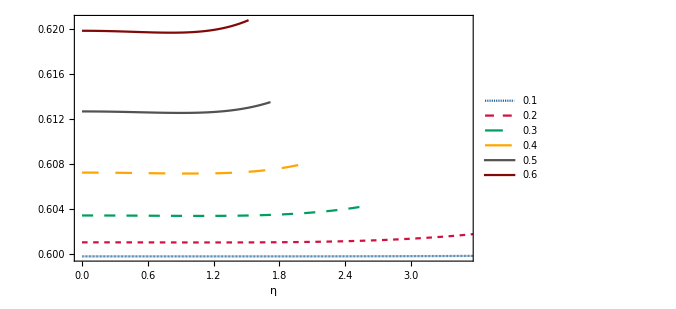

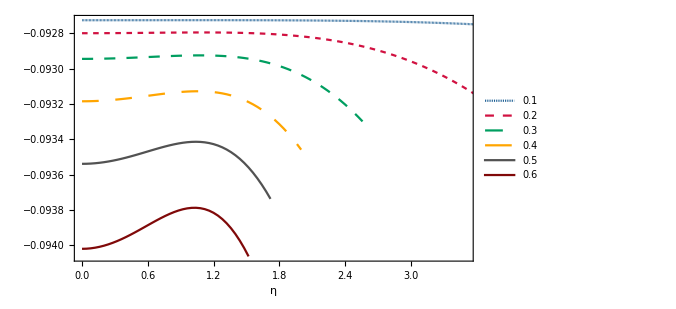

```mathematica
ListLinePlot[{Re[Ta[[1]]],Re[Ta[[2]]],Re[Ta[[3]]],Re[Ta[[4]]],Re[Ta[[5]]],Re[Ta[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[Ta[[1]]],Im[Ta[[2]]],Im[Ta[[3]]],Im[Ta[[4]]],Im[Ta[[5]]],Im[Ta[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100
(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100
(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100
(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100
```

0.143466

-0.419502

0.179107

-0.29282

#### Polar modes

```mathematica
Tp={{{0,0.5998194086196614-0.09272502565085786 ⅈ},{1/25+ⅈ/25,0.5998193974138055-0.09272502422211236 ⅈ},{2/25+(2 ⅈ)/25,0.5998193638044483-0.0927250199412528 ⅈ},{3/25+(3 ⅈ)/25,0.5998193078163307-0.09272501282442319 ⅈ},{4/25+(4 ⅈ)/25,0.5998192294906675-0.09272500289852617 ⅈ},{1/5+ⅈ/5,0.5998191288851558-0.09272499020122218 ⅈ},{6/25+(6 ⅈ)/25,0.5998190060739683-0.09272497478092681 ⅈ},{7/25+(7 ⅈ)/25,0.5998188611477498-0.09272495669680557 ⅈ},{8/25+(8 ⅈ)/25,0.5998186942136091-0.09272493601876965 ⅈ},{9/25+(9 ⅈ)/25,0.5998185053951107-0.09272491282746952 ⅈ},{2/5+(2 ⅈ)/5,0.5998182948322658-0.09272488721428795 ⅈ},{11/25+(11 ⅈ)/25,0.5998180626815199-0.09272485928133227 ⅈ},{12/25+(12 ⅈ)/25,0.5998178091157417-0.09272482914142535 ⅈ},{13/25+(13 ⅈ)/25,0.5998175343242086-0.09272479691809622 ⅈ},{14/25+(14 ⅈ)/25,0.5998172385125923-0.09272476274556862 ⅈ},{3/5+(3 ⅈ)/5,0.5998169219029411-0.09272472676875008 ⅈ},{16/25+(16 ⅈ)/25,0.5998165847336631-0.09272468914321841 ⅈ},{17/25+(17 ⅈ)/25,0.5998162272595059-0.09272465003520919 ⅈ},{18/25+(18 ⅈ)/25,0.5998158497515359-0.09272460962159915 ⅈ},{19/25+(19 ⅈ)/25,0.5998154524971157-0.09272456808989316 ⅈ},{4/5+(4 ⅈ)/5,0.5998150357998806-0.09272452563820552 ⅈ},{21/25+(21 ⅈ)/25,0.5998145999797121-0.09272448247524305 ⅈ},{22/25+(22 ⅈ)/25,0.5998141453727106-0.092724438820287 ⅈ},{23/25+(23 ⅈ)/25,0.5998136723311673-0.09272439490317215 ⅈ},{24/25+(24 ⅈ)/25,0.5998131812235329-0.09272435096426704 ⅈ},{1+ⅈ,0.5998126724343847-0.09272430725445206 ⅈ},{26/25+(26 ⅈ)/25,0.5998121463643938-0.09272426403509584 ⅈ},{27/25+(27 ⅈ)/25,0.5998116034302866-0.09272422157803305 ⅈ},{28/25+(28 ⅈ)/25,0.5998110440648088-0.09272418016553725 ⅈ},{29/25+(29 ⅈ)/25,0.5998104687166842-0.09272414009029625 ⅈ},{6/5+(6 ⅈ)/5,0.5998098778505727-0.09272410165538467 ⅈ},{31/25+(31 ⅈ)/25,0.599809271947027-0.09272406517423513 ⅈ},{32/25+(32 ⅈ)/25,0.5998086515024444-0.09272403097060945 ⅈ},{33/25+(33 ⅈ)/25,0.5998080170290208-0.09272399937856701 ⅈ},{34/25+(34 ⅈ)/25,0.5998073690546963-0.09272397074243438 ⅈ},{7/5+(7 ⅈ)/5,0.5998067081231057-0.09272394541677069 ⅈ},{36/25+(36 ⅈ)/25,0.5998060347935196-0.09272392376633458 ⅈ},{37/25+(37 ⅈ)/25,0.5998053496407877-0.0927239061660487 ⅈ},{38/25+(38 ⅈ)/25,0.5998046532552777-0.09272389300096191 ⅈ},{39/25+(39 ⅈ)/25,0.5998039462428113-0.0927238846662126 ⅈ},{8/5+(8 ⅈ)/5,0.5998032292245984-0.09272388156698966 ⅈ},{41/25+(41 ⅈ)/25,0.5998025028371661-0.09272388411849014 ⅈ},{42/25+(42 ⅈ)/25,0.5998017677322881-0.09272389274587962 ⅈ},{43/25+(43 ⅈ)/25,0.5998010245769093-0.09272390788424732 ⅈ},{44/25+(44 ⅈ)/25,0.5998002740530655-0.09272392997856317 ⅈ},{9/5+(9 ⅈ)/5,0.5997995168578024-0.09272395948363003 ⅈ},{46/25+(46 ⅈ)/25,0.59979875370309-0.09272399686403869 ⅈ},{47/25+(47 ⅈ)/25,0.5997979853157343-0.0927240425941165 ⅈ},{48/25+(48 ⅈ)/25,0.5997972124372831-0.09272409715788006 ⅈ},{49/25+(49 ⅈ)/25,0.5997964358239303-0.09272416104898139 ⅈ},{2+2 ⅈ,0.5997956562464156-0.0927242347706557 ⅈ},{51/25+(51 ⅈ)/25,0.5997948744899191-0.0927243188356671 ⅈ},{52/25+(52 ⅈ)/25,0.5997940913539535-0.09272441376625183 ⅈ},{53/25+(53 ⅈ)/25,0.5997933076522495-0.09272452009406129 ⅈ},{54/25+(54 ⅈ)/25,0.5997925242126384-0.09272463836010217 ⅈ},{11/5+(11 ⅈ)/5,0.5997917418769305-0.09272476911467573 ⅈ},{56/25+(56 ⅈ)/25,0.5997909615007856-0.09272491291731591 ⅈ},{57/25+(57 ⅈ)/25,0.5997901839535826-0.09272507033672425 ⅈ},{58/25+(58 ⅈ)/25,0.5997894101182799-0.09272524195070499 ⅈ},{59/25+(59 ⅈ)/25,0.5997886408912722-0.09272542834609687 ⅈ},{12/5+(12 ⅈ)/5,0.599787877182242-0.09272563011870505 ⅈ},{61/25+(61 ⅈ)/25,0.5997871199140046-0.09272584787322848 ⅈ},{62/25+(62 ⅈ)/25,0.5997863700223468-0.09272608222318873 ⅈ},{63/25+(63 ⅈ)/25,0.5997856284558599-0.09272633379085424 ⅈ},{64/25+(64 ⅈ)/25,0.5997848961757636-0.09272660320716558 ⅈ},{13/5+(13 ⅈ)/5,0.5997841741557297-0.09272689111165544 ⅈ},{66/25+(66 ⅈ)/25,0.5997834633816895-0.09272719815236981 ⅈ},{67/25+(67 ⅈ)/25,0.5997827648516412-0.09272752498578532 ⅈ},{68/25+(68 ⅈ)/25,0.5997820795754463-0.09272787227672605 ⅈ},{69/25+(69 ⅈ)/25,0.599781408574619-0.09272824069827719 ⅈ},{14/5+(14 ⅈ)/5,0.5997807528821075-0.09272863093169753 ⅈ},{71/25+(71 ⅈ)/25,0.5997801135420661-0.09272904366632935 ⅈ},{72/25+(72 ⅈ)/25,0.5997794916096191-0.0927294795995068 ⅈ},{73/25+(73 ⅈ)/25,0.5997788881506155-0.09272993943646204 ⅈ},{74/25+(74 ⅈ)/25,0.5997783042413746-0.09273042389022934 ⅈ},{3+3 ⅈ,0.599777740968419-0.09273093368154713 ⅈ},{76/25+(76 ⅈ)/25,0.5997771994282017-0.09273146953875704 ⅈ},{77/25+(77 ⅈ)/25,0.5997766807268199-0.09273203219770307 ⅈ},{78/25+(78 ⅈ)/25,0.5997761859797173-0.09273262240162602 ⅈ},{79/25+(79 ⅈ)/25,0.5997757163113764-0.09273324090105646 ⅈ},{16/5+(16 ⅈ)/5,0.5997752728549979-0.09273388845370745 ⅈ},{81/25+(81 ⅈ)/25,0.5997748567521687-0.09273456582436185 ⅈ},{82/25+(82 ⅈ)/25,0.5997744691525142-0.09273527378475974 ⅈ},{83/25+(83 ⅈ)/25,0.5997741112133435-0.09273601311348263 ⅈ},{84/25+(84 ⅈ)/25,0.5997737840992712-0.09273678459583531 ⅈ},{17/5+(17 ⅈ)/5,0.5997734889818349-0.09273758902372631 ⅈ},{86/25+(86 ⅈ)/25,0.5997732270390889-0.09273842719554422 ⅈ},{87/25+(87 ⅈ)/25,0.5997729994551894-0.09273929991603397 ⅈ},{88/25+(88 ⅈ)/25,0.5997728074199581-0.09274020799616865 ⅈ},{89/25+(89 ⅈ)/25,0.5997726521284318-0.09274115225302006 ⅈ},{18/5+(18 ⅈ)/5,0.5997725347803939-0.09274213350962726 ⅈ},{91/25+(91 ⅈ)/25,0.5997724565798874-0.0927431525948617 ⅈ},{92/25+(92 ⅈ)/25,0.5997724187347079-0.09274421034328986 ⅈ},{93/25+(93 ⅈ)/25,0.5997724224558795-0.09274530759503537 ⅈ},{94/25+(94 ⅈ)/25,0.5997724689571081-0.09274644519563593 ⅈ},{19/5+(19 ⅈ)/5,0.5997725594542126-0.09274762399590042 ⅈ},{96/25+(96 ⅈ)/25,0.5997726951645362-0.09274884485176181 ⅈ},{97/25+(97 ⅈ)/25,0.5997728773063329-0.09275010862412841 ⅈ},{98/25+(98 ⅈ)/25,0.5997731070981294-0.09275141617873214 ⅈ},{99/25+(99 ⅈ)/25,0.5997733857580647-0.09275276838597614 ⅈ},{4+4 ⅈ,0.5997737145031997-0.09275416612077718 ⅈ},{101/25+(101 ⅈ)/25,0.5997740945488027-0.09275561026240804 ⅈ},{102/25+(102 ⅈ)/25,0.599774527107604-0.09275710169433624 ⅈ},{103/25+(103 ⅈ)/25,0.5997750133890234-0.09275864130406138 ⅈ},{104/25+(104 ⅈ)/25,0.599775554598365-0.0927602299829497 ⅈ},{21/5+(21 ⅈ)/5,0.599776151935981-0.09276186862606545 ⅈ},{106/25+(106 ⅈ)/25,0.5997768065964013-0.09276355813200185 ⅈ},{107/25+(107 ⅈ)/25,0.5997775197674282-0.09276529940270868 ⅈ},{108/25+(108 ⅈ)/25,0.5997782926291962-0.09276709334331747 ⅈ},{109/25+(109 ⅈ)/25,0.5997791263531915-0.092768940861965 ⅈ},{22/5+(22 ⅈ)/5,0.5997800221012328-0.09277084286961561 ⅈ},{111/25+(111 ⅈ)/25,0.5997809810244138-0.09277280027987989 ⅈ},{112/25+(112 ⅈ)/25,0.5997820042619957-0.0927748140088324 ⅈ},{113/25+(113 ⅈ)/25,0.5997830929402623-0.09277688497482796 ⅈ},{114/25+(114 ⅈ)/25,0.5997842481713241-0.09277901409831336 ⅈ},{23/5+(23 ⅈ)/5,0.5997854710518733-0.09278120230164283 ⅈ},{116/25+(116 ⅈ)/25,0.599786762661888-0.09278345050888681 ⅈ},{117/25+(117 ⅈ)/25,0.5997881240632855-0.09278575964564102 ⅈ},{118/25+(118 ⅈ)/25,0.5997895562985142-0.09278813063883608 ⅈ},{119/25+(119 ⅈ)/25,0.5997910603890941-0.0927905644165421 ⅈ},{24/5+(24 ⅈ)/5,0.5997926373340898-0.0927930619077755 ⅈ},{121/25+(121 ⅈ)/25,0.5997942881085233-0.09279562404230392 ⅈ},{122/25+(122 ⅈ)/25,0.5997960136617208-0.09279825175045073 ⅈ},{123/25+(123 ⅈ)/25,0.5997978149155864-0.09280094596289828 ⅈ},{124/25+(124 ⅈ)/25,0.5997996927628044-0.0928037076104901 ⅈ},{5+5 ⅈ,0.5998016480649683-0.0928065376240349 ⅈ},{126/25+(126 ⅈ)/25,0.5998036816506244-0.09280943693411198 ⅈ},{127/25+(127 ⅈ)/25,0.5998057943132352-0.0928124064708726 ⅈ},{128/25+(128 ⅈ)/25,0.5998079868090553-0.09281544716384492 ⅈ},{129/25+(129 ⅈ)/25,0.5998102598549139-0.0928185599417415 ⅈ},{26/5+(26 ⅈ)/5,0.5998126141259028-0.09282174573226347 ⅈ},{131/25+(131 ⅈ)/25,0.5998150502529627-0.09282500546191189 ⅈ},{132/25+(132 ⅈ)/25,0.5998175688203647-0.09282834005579763 ⅈ},{133/25+(133 ⅈ)/25,0.5998201703630809-0.09283175043745415 ⅈ},{134/25+(134 ⅈ)/25,0.5998228553640386-0.09283523752865569 ⅈ},{27/5+(27 ⅈ)/5,0.5998256242512551-0.0928388022492354 ⅈ},{136/25+(136 ⅈ)/25,0.5998284773948411-0.09284244551691115 ⅈ},{137/25+(137 ⅈ)/25,0.5998314151038763-0.09284616824711309 ⅈ},{138/25+(138 ⅈ)/25,0.5998344376231364-0.09284997135281776 ⅈ},{139/25+(139 ⅈ)/25,0.5998375451296818-0.09285385574438888 ⅈ},{28/5+(28 ⅈ)/5,0.5998407377292851-0.09285782232942283 ⅈ},{141/25+(141 ⅈ)/25,0.5998440154526994-0.09286187201260379 ⅈ},{142/25+(142 ⅈ)/25,0.5998473782517543-0.09286600569556541 ⅈ},{143/25+(143 ⅈ)/25,0.599850825995275-0.09287022427676217 ⅈ},{144/25+(144 ⅈ)/25,0.599854358464811-0.09287452865135201 ⅈ},{29/5+(29 ⅈ)/5,0.5998579753501679-0.09287891971108943 ⅈ},{146/25+(146 ⅈ)/25,0.5998616762447321-0.09288339834423029 ⅈ},{147/25+(147 ⅈ)/25,0.599865460640575-0.09288796543545162 ⅈ},{148/25+(148 ⅈ)/25,0.5998693279233293-0.0928926218657857 ⅈ},{149/25+(149 ⅈ)/25,0.5998732773668226-0.09289736851257183 ⅈ},{6+6 ⅈ,0.5998773081274572-0.0929022062494235 ⅈ},{151/25+(151 ⅈ)/25,0.5998814192383218-0.0929071359462182 ⅈ},{152/25+(152 ⅈ)/25,0.5998856096030215-0.09291215846910815 ⅈ},{153/25+(153 ⅈ)/25,0.5998898779892126-0.09291727468055298 ⅈ},{154/25+(154 ⅈ)/25,0.5998942230218262-0.09292248543937935 ⅈ},{31/5+(31 ⅈ)/5,0.5998986431759594-0.09292779160086992 ⅈ},{156/25+(156 ⅈ)/25,0.5999031367694266-0.09293319401687926 ⅈ},{157/25+(157 ⅈ)/25,0.5999077019549428-0.09293869353598795 ⅈ},{158/25+(158 ⅈ)/25,0.5999123367119242-0.0929442910036866 ⅈ},{159/25+(159 ⅈ)/25,0.5999170388378869-0.09294998726260588 ⅈ},{32/5+(32 ⅈ)/5,0.5999218059394191-0.09295578315278366 ⅈ},{161/25+(161 ⅈ)/25,0.5999266354227044-0.09296167951198159 ⅈ},{162/25+(162 ⅈ)/25,0.5999315244835758-0.09296767717605023 ⅈ},{163/25+(163 ⅈ)/25,0.5999364700970712-0.0929737769793505 ⅈ},{164/25+(164 ⅈ)/25,0.5999414690064647-0.09297997975523366 ⅈ},{33/5+(33 ⅈ)/5,0.5999465177117483-0.0929862863365829 ⅈ},{166/25+(166 ⅈ)/25,0.5999516124575326-0.09299269755643011 ⅈ},{167/25+(167 ⅈ)/25,0.5999567492203336-0.0929992142486415 ⅈ},{168/25+(168 ⅈ)/25,0.5999619236952182-0.09300583724869009 ⅈ},{169/25+(169 ⅈ)/25,0.5999671312817696-0.09301256739451307 ⅈ},{34/5+(34 ⅈ)/5,0.5999723670693401-0.09301940552746812 ⅈ},{171/25+(171 ⅈ)/25,0.5999776258215501-0.0930263524933896 ⅈ},{172/25+(172 ⅈ)/25,0.5999829019599962-0.09303340914375946 ⅈ},{173/25+(173 ⅈ)/25,0.5999881895471458-0.0930405763369979 ⅈ},{174/25+(174 ⅈ)/25,0.5999934822683038-0.09304785493988744 ⅈ},{7+7 ⅈ,0.5999987734127448-0.0930552458291341 ⅈ},{176/25+(176 ⅈ)/25,0.6000040558537965-0.09306274989308622 ⅈ},{177/25+(177 ⅈ)/25,0.6000093220279609-0.0930703680336146 ⅈ},{178/25+(178 ⅈ)/25,0.6000145639129567-0.0930781011681734 ⅈ}},{{0,0.6010679439616654-0.0928013015698036 ⅈ},{1/25+ⅈ/25,0.6010677900781679-0.09280128063253586 ⅈ},{2/25+(2 ⅈ)/25,0.6010673284864979-0.092801217901501 ⅈ},{3/25+(3 ⅈ)/25,0.6010665593645355-0.09280111361918539 ⅈ},{4/25+(4 ⅈ)/25,0.6010654830080682-0.09280096818960852 ⅈ},{1/5+ⅈ/5,0.6010640998303106-0.09280078217820947 ⅈ},{6/25+(6 ⅈ)/25,0.6010624103610106-0.0928005563116572 ⅈ},{7/25+(7 ⅈ)/25,0.6010604152452993-0.0928002914776081 ⅈ},{8/25+(8 ⅈ)/25,0.6010581152422755-0.0927999887244065 ⅈ},{9/25+(9 ⅈ)/25,0.601055511223323-0.09279964926073128 ⅈ},{2/5+(2 ⅈ)/5,0.6010526041701553-0.09279927445518663 ⅈ},{11/25+(11 ⅈ)/25,0.6010493951725815-0.09279886583583404 ⅈ},{12/25+(12 ⅈ)/25,0.6010458854259852-0.09279842508966941 ⅈ},{13/25+(13 ⅈ)/25,0.6010420762285102-0.0927979540620403 ⅈ},{14/25+(14 ⅈ)/25,0.6010379689779455-0.09279745475600427 ⅈ},{3/5+(3 ⅈ)/5,0.6010335651682922-0.09279692933162723 ⅈ},{16/25+(16 ⅈ)/25,0.6010288663860158-0.09279638010522107 ⅈ},{17/25+(17 ⅈ)/25,0.6010238743059554-0.09279580954851833 ⅈ},{18/25+(18 ⅈ)/25,0.6010185906868908-0.09279522028778375 ⅈ},{19/25+(19 ⅈ)/25,0.6010130173667466-0.09279461510286106 ⅈ},{4/5+(4 ⅈ)/5,0.6010071562574183-0.09279399692615485 ⅈ},{21/25+(21 ⅈ)/25,0.6010010093392093-0.09279336884154459 ⅈ},{22/25+(22 ⅈ)/25,0.6009945786548542-0.09279273408323041 ⅈ},{23/25+(23 ⅈ)/25,0.600987866303116-0.09279209603451034 ⅈ},{24/25+(24 ⅈ)/25,0.600980874431934-0.09279145822648563 ⅈ},{1+ⅈ,0.6009736052311015-0.09279082433669544 ⅈ},{26/25+(26 ⅈ)/25,0.6009660609244509-0.09279019818767789 ⅈ},{27/25+(27 ⅈ)/25,0.6009582437615193-0.09278958374545421 ⅈ},{28/25+(28 ⅈ)/25,0.6009501560086771-0.09278898511794564 ⅈ},{29/25+(29 ⅈ)/25,0.6009417999396758-0.09278840655330467 ⅈ},{6/5+(6 ⅈ)/5,0.6009331778256045-0.0927878524381742 ⅈ},{31/25+(31 ⅈ)/25,0.6009242919242084-0.09278732729586972 ⅈ},{32/25+(32 ⅈ)/25,0.6009151444685458-0.09278683578448137 ⅈ},{33/25+(33 ⅈ)/25,0.6009057376549413-0.09278638269489824 ⅈ},{34/25+(34 ⅈ)/25,0.6008960736302043-0.09278597294875449 ⅈ},{7/5+(7 ⅈ)/5,0.6008861544780669-0.09278561159629653 ⅈ},{36/25+(36 ⅈ)/25,0.6008759822048036-0.09278530381417398 ⅈ},{37/25+(37 ⅈ)/25,0.6008655587239865-0.09278505490315175 ⅈ},{38/25+(38 ⅈ)/25,0.6008548858403275-0.09278487028574758 ⅈ},{39/25+(39 ⅈ)/25,0.6008439652325601-0.0927847555037954 ⅈ},{8/5+(8 ⅈ)/5,0.6008327984353077-0.09278471621593853 ⅈ},{41/25+(41 ⅈ)/25,0.6008213868198796-0.09278475819505193 ⅈ},{42/25+(42 ⅈ)/25,0.6008097315739416-0.09278488732559913 ⅈ},{43/25+(43 ⅈ)/25,0.6007978336799916-0.0927851096009306 ⅈ},{44/25+(44 ⅈ)/25,0.6007856938925842-0.09278543112052377 ⅈ},{9/5+(9 ⅈ)/5,0.6007733127142262-0.09278585808717253 ⅈ},{46/25+(46 ⅈ)/25,0.6007606903698783-0.09278639680413472 ⅈ},{47/25+(47 ⅈ)/25,0.6007478267799802-0.09278705367224312 ⅈ},{48/25+(48 ⅈ)/25,0.6007347215319261-0.09278783518699003 ⅈ},{49/25+(49 ⅈ)/25,0.6007213738498999-0.09278874793559784 ⅈ},{2+2 ⅈ,0.600707782562989-0.0927897985940822 ⅈ},{51/25+(51 ⅈ)/25,0.6006939460714773-0.09279099392432864 ⅈ},{52/25+(52 ⅈ)/25,0.6006798623112315-0.09279234077119193 ⅈ},{53/25+(53 ⅈ)/25,0.6006655287160687-0.0927938460596393 ⅈ},{54/25+(54 ⅈ)/25,0.6006509421780124-0.09279551679195495 ⅈ},{11/5+(11 ⅈ)/5,0.6006360990053223-0.09279736004502745 ⅈ},{56/25+(56 ⅈ)/25,0.6006209948781875-0.09279938296774973 ⅈ},{57/25+(57 ⅈ)/25,0.6006056248019689-0.09280159277854748 ⅈ},{58/25+(58 ⅈ)/25,0.60058998305787-0.09280399676308075 ⅈ},{59/25+(59 ⅈ)/25,0.6005740631509191-0.09280660227214194 ⅈ},{12/5+(12 ⅈ)/5,0.6005578577551289-0.09280941671978953 ⅈ},{61/25+(61 ⅈ)/25,0.600541358655722-0.09281244758176208 ⅈ},{62/25+(62 ⅈ)/25,0.600524556688279-0.09281570239421828 ⅈ},{63/25+(63 ⅈ)/25,0.6005074416746985-0.09281918875284499 ⅈ},{64/25+(64 ⅈ)/25,0.6004900023558154-0.09282291431240239 ⅈ},{13/5+(13 ⅈ)/5,0.6004722263206056-0.09282688678675097 ⅈ},{66/25+(66 ⅈ)/25,0.6004540999317928-0.09283111394944214 ⅈ},{67/25+(67 ⅈ)/25,0.6004356082477893-0.0928356036349315 ⅈ},{68/25+(68 ⅈ)/25,0.6004167349408498-0.09284036374050267 ⅈ},{69/25+(69 ⅈ)/25,0.6003974622113464-0.09284540222898148 ⅈ},{14/5+(14 ⅈ)/5,0.6003777706980854-0.09285072713233745 ⅈ},{71/25+(71 ⅈ)/25,0.600357639384605-0.09285634655626929 ⅈ},{72/25+(72 ⅈ)/25,0.6003370455014145-0.09286226868588442 ⅈ},{73/25+(73 ⅈ)/25,0.6003159644241723-0.09286850179258511 ⅈ},{74/25+(74 ⅈ)/25,0.6002943695678151-0.09287505424229026 ⅈ},{3+3 ⅈ,0.6002722322767134-0.09288193450511464 ⅈ},{76/25+(76 ⅈ)/25,0.6002495217109635-0.09288915116665492 ⅈ},{77/25+(77 ⅈ)/25,0.6002262047289857-0.09289671294101867 ⅈ},{78/25+(78 ⅈ)/25,0.6002022457666705-0.09290462868575247 ⅈ},{79/25+(79 ⅈ)/25,0.6001776067133887-0.09291290741882662 ⅈ},{16/5+(16 ⅈ)/5,0.6001522467852775-0.09292155833783305 ⅈ},{81/25+(81 ⅈ)/25,0.6001261223963145-0.09293059084155987 ⅈ},{82/25+(82 ⅈ)/25,0.6000991870278226-0.09294001455410701 ⅈ},{83/25+(83 ⅈ)/25,0.6000713910971756-0.09294983935169127 ⅈ},{84/25+(84 ⅈ)/25,0.6000426818266466-0.09296007539229699 ⅈ},{17/5+(17 ⅈ)/5,0.6000130031135037-0.09297073314830198 ⅈ},{86/25+(86 ⅈ)/25,0.5999822954026713-0.09298182344219438 ⅈ},{87/25+(87 ⅈ)/25,0.5999504955634903-0.09299335748547301 ⅈ},{88/25+(88 ⅈ)/25,0.5999175367723562-0.0930053469207773 ⅈ},{89/25+(89 ⅈ)/25,0.5998833484032957-0.09301780386726194 ⅈ},{18/5+(18 ⅈ)/5,0.5998478559288173-0.0930307409691648 ⅈ},{91/25+(91 ⅈ)/25,0.5998109808337121-0.0930441714474488 ⅈ}},{{0,0.6034692070457216-0.0929571102789681 ⅈ},{1/25+ⅈ/25,0.6034685828050661-0.09295701624370878 ⅈ},{2/25+(2 ⅈ)/25,0.6034667101032172-0.09295673452455101 ⅈ},{3/25+(3 ⅈ)/25,0.6034635890052662-0.09295626628211315 ⅈ},{4/25+(4 ⅈ)/25,0.6034592196136257-0.09295561344999105 ⅈ},{1/5+ⅈ/5,0.6034536020610872-0.09295477873393394 ⅈ},{6/25+(6 ⅈ)/25,0.6034467365001843-0.09295376561055761 ⅈ},{7/25+(7 ⅈ)/25,0.6034386230894486-0.0929525783256886 ⅈ},{8/25+(8 ⅈ)/25,0.6034292619765014-0.09295122189233587 ⅈ},{9/25+(9 ⅈ)/25,0.6034186532779187-0.09294970208829022 ⅈ},{2/5+(2 ⅈ)/5,0.6034067970557929-0.09294802545334963 ⅈ},{11/25+(11 ⅈ)/25,0.6033936932909049-0.0929461992861694 ⅈ},{12/25+(12 ⅈ)/25,0.6033793418523976-0.09294423164073659 ⅈ},{13/25+(13 ⅈ)/25,0.6033637424638544-0.09294213132247166 ⅈ},{14/25+(14 ⅈ)/25,0.6033468946656432-0.09293990788395526 ⅈ},{3/5+(3 ⅈ)/5,0.6033287977734051-0.09293757162028979 ⅈ},{16/25+(16 ⅈ)/25,0.6033094508325222-0.0929351335640888 ⅈ},{17/25+(17 ⅈ)/25,0.6032888525684441-0.09293260548013224 ⅈ},{18/25+(18 ⅈ)/25,0.6032670013326596-0.09292999985965905 ⅈ},{19/25+(19 ⅈ)/25,0.6032438950441719-0.09292732991434728 ⅈ},{4/5+(4 ⅈ)/5,0.6032195311262738-0.09292460956998477 ⅈ},{21/25+(21 ⅈ)/25,0.603193906438436-0.0929218534598643 ⅈ},{22/25+(22 ⅈ)/25,0.6031670172031036-0.09291907691793146 ⅈ},{23/25+(23 ⅈ)/25,0.6031388589271925-0.09291629597172987 ⅈ},{24/25+(24 ⅈ)/25,0.6031094263180811-0.09291352733518962 ⅈ},{1+ⅈ,0.6030787131938761-0.09291078840131822 ⅈ},{26/25+(26 ⅈ)/25,0.6030467123877498-0.09290809723486432 ⅈ},{27/25+(27 ⅈ)/25,0.6030134156461355-0.0929054725650347 ⅈ},{28/25+(28 ⅈ)/25,0.6029788135205869-0.09290293377836183 ⅈ},{29/25+(29 ⅈ)/25,0.6029428952531096-0.09290050091183034 ⅈ},{6/5+(6 ⅈ)/5,0.6029056486548038-0.09289819464639383 ⅈ},{31/25+(31 ⅈ)/25,0.6028670599776687-0.0928960363010251 ⅈ},{32/25+(32 ⅈ)/25,0.6028271137794604-0.0928940478274698 ⅈ},{33/25+(33 ⅈ)/25,0.6027857927815282-0.0928922518058908 ⅈ},{34/25+(34 ⅈ)/25,0.6027430777196154-0.09289067144161907 ⅈ},{7/5+(7 ⅈ)/5,0.6026989471876604-0.09288933056324883 ⅈ},{36/25+(36 ⅈ)/25,0.602653377474721-0.09288825362234454 ⅈ},{37/25+(37 ⅈ)/25,0.6026063423952311-0.09288746569505733 ⅈ},{38/25+(38 ⅈ)/25,0.6025578131129092-0.09288699248597566 ⅈ},{39/25+(39 ⅈ)/25,0.6025077579587699-0.09288686033456828 ⅈ},{8/5+(8 ⅈ)/5,0.6024561422438388-0.09288709622460894 ⅈ},{41/25+(41 ⅈ)/25,0.6024029280673567-0.09288772779700506 ⅈ},{42/25+(42 ⅈ)/25,0.6023480741214571-0.09288878336647487 ⅈ},{43/25+(43 ⅈ)/25,0.602291535493549-0.09289029194255848 ⅈ},{44/25+(44 ⅈ)/25,0.6022332634679071-0.09289228325545675 ⅈ},{9/5+(9 ⅈ)/5,0.6021732053282844-0.09289478778722143 ⅈ},{46/25+(46 ⅈ)/25,0.6021113041637237-0.0928978368088244 ⅈ},{47/25+(47 ⅈ)/25,0.6020474986801322-0.09290146242363755 ⅈ},{48/25+(48 ⅈ)/25,0.6019817230206401-0.09290569761783542 ⅈ},{49/25+(49 ⅈ)/25,0.6019139065982549-0.0929105763182127 ⅈ},{2+2 ⅈ,0.6018439739448583-0.09291613345784762 ⅈ},{51/25+(51 ⅈ)/25,0.6017718445811998-0.0929224050499734 ⅈ},{52/25+(52 ⅈ)/25,0.6016974329131518-0.09292942827031152 ⅈ},{53/25+(53 ⅈ)/25,0.601620648160188-0.09293724154797495 ⅈ},{54/25+(54 ⅈ)/25,0.6015413943227323-0.09294588466487422 ⅈ},{11/5+(11 ⅈ)/5,0.6014595701957538-0.09295539886331919 ⅈ},{56/25+(56 ⅈ)/25,0.6013750694367017-0.09296582696123133 ⅈ},{57/25+(57 ⅈ)/25,0.6012877806965707-0.09297721347404055 ⅈ},{58/25+(58 ⅈ)/25,0.6011975878235356-0.09298960474193156 ⅈ},{59/25+(59 ⅈ)/25,0.6011043701491501-0.09300304906064571 ⅈ},{12/5+(12 ⅈ)/5,0.601008002867536-0.09301759681350712 ⅈ},{61/25+(61 ⅈ)/25,0.6009083575182441-0.09303330060175566 ⅈ},{62/25+(62 ⅈ)/25,0.6008053025834734-0.09305021536962475 ⅈ},{63/25+(63 ⅈ)/25,0.6006987042100684-0.09306839851992249 ⅈ},{64/25+(64 ⅈ)/25,0.6005884270660486-0.09308791001517892 ⅈ}},{{0,0.6073157922557862-0.09322162990223094 ⅈ},{1/25+ⅈ/25,0.6073142745531602-0.093221369481009 ⅈ},{2/25+(2 ⅈ)/25,0.6073097211566744-0.09322058939035849 ⅈ},{3/25+(3 ⅈ)/25,0.6073021312102308-0.09321929315176296 ⅈ},{4/25+(4 ⅈ)/25,0.6072915032662911-0.093217486633375 ⅈ},{1/5+ⅈ/5,0.6072778352600945-0.09321517804945863 ⅈ},{6/25+(6 ⅈ)/25,0.6072611244713821-0.09321237795927435 ⅈ},{7/25+(7 ⅈ)/25,0.6072413674750939-0.09320909926569577 ⅈ},{8/25+(8 ⅈ)/25,0.6072185600809551-0.09320535721358374 ⅈ},{9/25+(9 ⅈ)/25,0.6071926972619364-0.0932011693880093 ⅈ},{2/5+(2 ⅈ)/5,0.6071637730714585-0.09319655571234484 ⅈ},{11/25+(11 ⅈ)/25,0.6071317805493327-0.0931915384463453 ⅈ},{12/25+(12 ⅈ)/25,0.6070967116163777-0.09318614218431416 ⅈ},{13/25+(13 ⅈ)/25,0.6070585569577173-0.09318039385348999 ⅈ},{14/25+(14 ⅈ)/25,0.6070173058947871-0.09317432271281668 ⅈ},{3/5+(3 ⅈ)/5,0.6069729462461478-0.09316796035229259 ⅈ},{16/25+(16 ⅈ)/25,0.6069254641772787-0.09316134069313807 ⅈ},{17/25+(17 ⅈ)/25,0.6068748440396183-0.09315449998905775 ⅈ},{18/25+(18 ⅈ)/25,0.606821068199248-0.093147476828931 ⅈ},{19/25+(19 ⅈ)/25,0.6067641168557657-0.093140312141315 ⅈ},{4/5+(4 ⅈ)/5,0.6067039678520809-0.09313304920120816 ⅈ},{21/25+(21 ⅈ)/25,0.606640596476088-0.09312573363958582 ⅈ},{22/25+(22 ⅈ)/25,0.6065739752554393-0.09311841345629542 ⅈ},{23/25+(23 ⅈ)/25,0.6065040737469609-0.09311113903696967 ⅈ},{24/25+(24 ⅈ)/25,0.6064308583226176-0.09310396317469412 ⅈ},{1+ⅈ,0.6063542919543711-0.09309694109724556 ⅈ},{26/25+(26 ⅈ)/25,0.6062743340007771-0.09309013050079151 ⅈ},{27/25+(27 ⅈ)/25,0.606190939998732-0.09308359159101212 ⅈ},{28/25+(28 ⅈ)/25,0.6061040614644474-0.0930773871326646 ⅈ},{29/25+(29 ⅈ)/25,0.6060136457084563-0.09307158250865336 ⅈ},{6/5+(6 ⅈ)/5,0.6059196356703002-0.0930662457896938 ⅈ},{31/25+(31 ⅈ)/25,0.6058219697794476-0.09306144781564107 ⅈ},{32/25+(32 ⅈ)/25,0.6057205818500263-0.09305726228950559 ⅈ},{33/25+(33 ⅈ)/25,0.6056154010180399-0.09305376588507329 ⅈ},{34/25+(34 ⅈ)/25,0.6055063517309175-0.09305103836886784 ⅈ},{7/5+(7 ⅈ)/5,0.605393353800496-0.09304916273694007 ⅈ},{36/25+(36 ⅈ)/25,0.6052763225318083-0.09304822536661153 ⅈ},{37/25+(37 ⅈ)/25,0.6051551689413519-0.09304831618281982 ⅈ},{38/25+(38 ⅈ)/25,0.6050298000797717-0.09304952883810387 ⅈ},{39/25+(39 ⅈ)/25,0.604900119475063-0.09305196090449559 ⅈ},{8/5+(8 ⅈ)/5,0.60476602771342-0.09305571407464745 ⅈ},{41/25+(41 ⅈ)/25,0.6046274231756291-0.09306089436839872 ⅈ},{42/25+(42 ⅈ)/25,0.6044842029473414-0.09306761233967276 ⅈ},{43/25+(43 ⅈ)/25,0.604336263921526-0.09307598327709893 ⅈ},{44/25+(44 ⅈ)/25,0.6041835041107998-0.09308612739007495 ⅈ},{9/5+(9 ⅈ)/5,0.6040258241859752-0.09309816997018455 ⅈ},{46/25+(46 ⅈ)/25,0.6038631292549546-0.09311224151596843 ⅈ},{47/25+(47 ⅈ)/25,0.6036953308928615-0.0931284778071358 ⅈ},{48/25+(48 ⅈ)/25,0.6035223494299226-0.09314701991245075 ⅈ},{49/25+(49 ⅈ)/25,0.6033441164979951-0.09316801411388895 ⅈ},{2+2 ⅈ,0.6031605778297293-0.09319161172835796 ⅈ}},{{0,0.6128212550016545-0.09362039153182755 ⅈ},{1/25+ⅈ/25,0.6128184670081709-0.0936198357134614 ⅈ},{2/25+(2 ⅈ)/25,0.6128101023220799-0.09361817100740168 ⅈ},{3/25+(3 ⅈ)/25,0.612796158845837-0.09361540566837417 ⅈ},{4/25+(4 ⅈ)/25,0.6127766330506573-0.09361155346020039 ⅈ},{1/5+ⅈ/5,0.6127515199372584-0.09360663366675144 ⅈ},{6/25+(6 ⅈ)/25,0.6127208129777074-0.09360067110674432 ⅈ},{7/25+(7 ⅈ)/25,0.6126845040418051-0.09359369615311343 ⅈ},{8/25+(8 ⅈ)/25,0.6126425833089957-0.09358574475727803 ⅈ},{9/25+(9 ⅈ)/25,0.6125950391670317-0.09357685847867181 ⅈ},{2/5+(2 ⅈ)/5,0.6125418580989712-0.09356708451999572 ⅈ},{11/25+(11 ⅈ)/25,0.6124830245604691-0.09355647576875853 ⅈ},{12/25+(12 ⅈ)/25,0.6124185208497913-0.09354509084577217 ⅈ},{13/25+(13 ⅈ)/25,0.6123483269735075-0.09353299416139108 ⅈ},{14/25+(14 ⅈ)/25,0.6122724205114554-0.09352025598040599 ⅈ},{3/5+(3 ⅈ)/5,0.6121907764852929-0.0935069524966352 ⅈ},{16/25+(16 ⅈ)/25,0.6121033672358067-0.0934931659183863 ⅈ},{17/25+(17 ⅈ)/25,0.612010162315115-0.09347898456608872 ⅈ},{18/25+(18 ⅈ)/25,0.6119111284010224-0.09346450298351212 ⅈ},{19/25+(19 ⅈ)/25,0.6118062292420416-0.09344982206407566 ⅈ},{4/5+(4 ⅈ)/5,0.6116954256430249-0.09343504919380231 ⅈ},{21/25+(21 ⅈ)/25,0.6115786755029271-0.09342029841247282 ⅈ},{22/25+(22 ⅈ)/25,0.6114559339179667-0.09340569059444784 ⅈ},{23/25+(23 ⅈ)/25,0.6113271533653496-0.09339135365043479 ⅈ},{24/25+(24 ⅈ)/25,0.6111922839847413-0.09337742275114991 ⅈ},{1+ⅈ,0.6110512739768084-0.09336404057331345 ⅈ},{26/25+(26 ⅈ)/25,0.6109040701403228-0.0933513575676856 ⅈ},{27/25+(27 ⅈ)/25,0.6107506185714934-0.09333953224784723 ⅈ},{28/25+(28 ⅈ)/25,0.6105908655512315-0.09332873149710331 ⅈ},{29/25+(29 ⅈ)/25,0.6104247586478918-0.09331913088918006 ⅈ},{6/5+(6 ⅈ)/5,0.6102522480644496-0.09331091501626225 ⅈ},{31/25+(31 ⅈ)/25,0.6100732882599512-0.09330427781530881 ⅈ},{32/25+(32 ⅈ)/25,0.6098878398751261-0.09329942288049774 ⅈ},{33/25+(33 ⅈ)/25,0.6096958719910613-0.0932965637460413 ⅈ},{34/25+(34 ⅈ)/25,0.6094973647474888-0.09329592411954366 ⅈ},{7/5+(7 ⅈ)/5,0.6092923123432428-0.09329773804159276 ⅈ},{36/25+(36 ⅈ)/25,0.6090807264354762-0.09330224994252077 ⅈ},{37/25+(37 ⅈ)/25,0.6088626399459889-0.09330971456243786 ⅈ},{38/25+(38 ⅈ)/25,0.6086381112722878-0.09332039669599658 ⅈ},{39/25+(39 ⅈ)/25,0.608407228887579-0.09333457071925544 ⅈ},{8/5+(8 ⅈ)/5,0.6081701162977827-0.09335251985289265 ⅈ},{41/25+(41 ⅈ)/25,0.6079269373049915-0.09337453511439324 ⅈ},{42/25+(42 ⅈ)/25,0.6076779015059237-0.09340091391224128 ⅈ},{43/25+(43 ⅈ)/25,0.6074232699314956-0.09343195823814138 ⅈ}},{{0,0.6200994657857434-0.09417208832732378 ⅈ},{1/25+ⅈ/25,0.6200951708938669-0.09417108040412868 ⅈ},{2/25+(2 ⅈ)/25,0.6200822854715722-0.09416806202006793 ⅈ},{3/25+(3 ⅈ)/25,0.6200608073214534-0.09416304935306713 ⅈ},{4/25+(4 ⅈ)/25,0.6200307327733076-0.09415606940229845 ⅈ},{1/5+ⅈ/5,0.61999205668931-0.09414716004605046 ⅈ},{6/25+(6 ⅈ)/25,0.6199447724690499-0.09413637012202362 ⅈ},{7/25+(7 ⅈ)/25,0.6198888720627161-0.09412375953182044 ⅈ},{8/25+(8 ⅈ)/25,0.6198243459976844-0.0941093993705682 ⅈ},{9/25+(9 ⅈ)/25,0.6197511834251941-0.094093372082825 ⅈ},{2/5+(2 ⅈ)/5,0.6196693721953995-0.09407577164613819 ⅈ},{11/25+(11 ⅈ)/25,0.6195788989708474-0.09405670378381853 ⅈ},{12/25+(12 ⅈ)/25,0.6194797493904135-0.09403628620865104 ⅈ},{13/25+(13 ⅈ)/25,0.6193719082979535-0.09401464889939477 ⅈ},{14/25+(14 ⅈ)/25,0.6192553600523741-0.09399193441195515 ⅈ},{3/5+(3 ⅈ)/5,0.6191300889385639-0.09396829822704775 ⅈ},{16/25+(16 ⅈ)/25,0.6189960797015913-0.09394390913594318 ⅈ},{17/25+(17 ⅈ)/25,0.6188533182297998-0.0939189496654312 ⅈ},{18/25+(18 ⅈ)/25,0.6187017924158486-0.09389361654240268 ⅈ},{19/25+(19 ⅈ)/25,0.6185414932283054-0.09386812119732217 ⅈ},{4/5+(4 ⅈ)/5,0.6183724160299998-0.09384269030425638 ⅈ},{21/25+(21 ⅈ)/25,0.6181945621828361-0.09381756635290506 ⅈ},{22/25+(22 ⅈ)/25,0.6180079409819728-0.09379300824513447 ⅈ},{23/25+(23 ⅈ)/25,0.617812571964919-0.09376929190468572 ⅈ},{24/25+(24 ⅈ)/25,0.6176084876428655-0.09374671088390249 ⅈ},{1+ⅈ,0.6173957367020533-0.09372557694535788 ⅈ},{26/25+(26 ⅈ)/25,0.6171743877216809-0.09370622058908969 ⅈ},{27/25+(27 ⅈ)/25,0.6169445334512167-0.09368899148772852 ⅈ},{28/25+(28 ⅈ)/25,0.6167062956833502-0.093674258782204 ⅈ},{29/25+(29 ⅈ)/25,0.6164598307485494-0.09366241118009021 ⅈ},{6/5+(6 ⅈ)/5,0.6162053356425268-0.09365385678738987 ⅈ},{31/25+(31 ⅈ)/25,0.6159430547783155-0.09364902259314921 ⅈ},{32/25+(32 ⅈ)/25,0.6156732873295231-0.09364835351556339 ⅈ},{33/25+(33 ⅈ)/25,0.615396395100467-0.09365231090918956 ⅈ},{34/25+(34 ⅈ)/25,0.6151128108223275-0.0936613704268281 ⅈ},{7/5+(7 ⅈ)/5,0.6148230467327757-0.09367601912808018 ⅈ},{36/25+(36 ⅈ)/25,0.614527703250889-0.09369675173122222 ⅈ},{37/25+(37 ⅈ)/25,0.6142274775114498-0.09372406591752712 ⅈ},{38/25+(38 ⅈ)/25,0.6139231714755515-0.09375845661907915 ⅈ}}};
```

```mathematica
Tdp={{{0.5998194086196614-0.09272502565085786 ⅈ},{0.5998193974138055-0.09272502422211236 ⅈ},{0.5998193638044483-0.0927250199412528 ⅈ},{0.5998193078163307-0.09272501282442319 ⅈ},{0.5998192294906675-0.09272500289852617 ⅈ},{0.5998191288851558-0.09272499020122218 ⅈ},{0.5998190060739683-0.09272497478092681 ⅈ},{0.5998188611477498-0.09272495669680557 ⅈ},{0.5998186942136091-0.09272493601876965 ⅈ},{0.5998185053951107-0.09272491282746952 ⅈ},{0.5998182948322658-0.09272488721428795 ⅈ},{0.5998180626815199-0.09272485928133227 ⅈ},{0.5998178091157417-0.09272482914142535 ⅈ},{0.5998175343242086-0.09272479691809622 ⅈ},{0.5998172385125923-0.09272476274556862 ⅈ},{0.5998169219029411-0.09272472676875008 ⅈ},{0.5998165847336631-0.09272468914321841 ⅈ},{0.5998162272595059-0.09272465003520919 ⅈ},{0.5998158497515359-0.09272460962159915 ⅈ},{0.5998154524971157-0.09272456808989316 ⅈ},{0.5998150357998806-0.09272452563820552 ⅈ},{0.5998145999797121-0.09272448247524305 ⅈ},{0.5998141453727106-0.092724438820287 ⅈ},{0.5998136723311673-0.09272439490317215 ⅈ},{0.5998131812235329-0.09272435096426704 ⅈ},{0.5998126724343847-0.09272430725445206 ⅈ},{0.5998121463643938-0.09272426403509584 ⅈ},{0.5998116034302866-0.09272422157803305 ⅈ},{0.5998110440648088-0.09272418016553725 ⅈ},{0.5998104687166842-0.09272414009029625 ⅈ},{0.5998098778505727-0.09272410165538467 ⅈ},{0.599809271947027-0.09272406517423513 ⅈ},{0.5998086515024444-0.09272403097060945 ⅈ},{0.5998080170290208-0.09272399937856701 ⅈ},{0.5998073690546963-0.09272397074243438 ⅈ},{0.5998067081231057-0.09272394541677069 ⅈ},{0.5998060347935196-0.09272392376633458 ⅈ},{0.5998053496407877-0.0927239061660487 ⅈ},{0.5998046532552777-0.09272389300096191 ⅈ},{0.5998039462428113-0.0927238846662126 ⅈ},{0.5998032292245984-0.09272388156698966 ⅈ},{0.5998025028371661-0.09272388411849014 ⅈ},{0.5998017677322881-0.09272389274587962 ⅈ},{0.5998010245769093-0.09272390788424732 ⅈ},{0.5998002740530655-0.09272392997856317 ⅈ},{0.5997995168578024-0.09272395948363003 ⅈ},{0.59979875370309-0.09272399686403869 ⅈ},{0.5997979853157343-0.0927240425941165 ⅈ},{0.5997972124372831-0.09272409715788006 ⅈ},{0.5997964358239303-0.09272416104898139 ⅈ},{0.5997956562464156-0.0927242347706557 ⅈ},{0.5997948744899191-0.0927243188356671 ⅈ},{0.5997940913539535-0.09272441376625183 ⅈ},{0.5997933076522495-0.09272452009406129 ⅈ},{0.5997925242126384-0.09272463836010217 ⅈ},{0.5997917418769305-0.09272476911467573 ⅈ},{0.5997909615007856-0.09272491291731591 ⅈ},{0.5997901839535826-0.09272507033672425 ⅈ},{0.5997894101182799-0.09272524195070499 ⅈ},{0.5997886408912722-0.09272542834609687 ⅈ},{0.599787877182242-0.09272563011870505 ⅈ},{0.5997871199140046-0.09272584787322848 ⅈ},{0.5997863700223468-0.09272608222318873 ⅈ},{0.5997856284558599-0.09272633379085424 ⅈ},{0.5997848961757636-0.09272660320716558 ⅈ},{0.5997841741557297-0.09272689111165544 ⅈ},{0.5997834633816895-0.09272719815236981 ⅈ},{0.5997827648516412-0.09272752498578532 ⅈ},{0.5997820795754463-0.09272787227672605 ⅈ},{0.599781408574619-0.09272824069827719 ⅈ},{0.5997807528821075-0.09272863093169753 ⅈ},{0.5997801135420661-0.09272904366632935 ⅈ},{0.5997794916096191-0.0927294795995068 ⅈ},{0.5997788881506155-0.09272993943646204 ⅈ},{0.5997783042413746-0.09273042389022934 ⅈ},{0.599777740968419-0.09273093368154713 ⅈ},{0.5997771994282017-0.09273146953875704 ⅈ},{0.5997766807268199-0.09273203219770307 ⅈ},{0.5997761859797173-0.09273262240162602 ⅈ},{0.5997757163113764-0.09273324090105646 ⅈ},{0.5997752728549979-0.09273388845370745 ⅈ},{0.5997748567521687-0.09273456582436185 ⅈ},{0.5997744691525142-0.09273527378475974 ⅈ},{0.5997741112133435-0.09273601311348263 ⅈ},{0.5997737840992712-0.09273678459583531 ⅈ},{0.5997734889818349-0.09273758902372631 ⅈ},{0.5997732270390889-0.09273842719554422 ⅈ},{0.5997729994551894-0.09273929991603397 ⅈ},{0.5997728074199581-0.09274020799616865 ⅈ},{0.5997726521284318-0.09274115225302006 ⅈ},{0.5997725347803939-0.09274213350962726 ⅈ},{0.5997724565798874-0.0927431525948617 ⅈ},{0.5997724187347079-0.09274421034328986 ⅈ},{0.5997724224558795-0.09274530759503537 ⅈ},{0.5997724689571081-0.09274644519563593 ⅈ},{0.5997725594542126-0.09274762399590042 ⅈ},{0.5997726951645362-0.09274884485176181 ⅈ},{0.5997728773063329-0.09275010862412841 ⅈ},{0.5997731070981294-0.09275141617873214 ⅈ},{0.5997733857580647-0.09275276838597614 ⅈ},{0.5997737145031997-0.09275416612077718 ⅈ},{0.5997740945488027-0.09275561026240804 ⅈ},{0.599774527107604-0.09275710169433624 ⅈ},{0.5997750133890234-0.09275864130406138 ⅈ},{0.599775554598365-0.0927602299829497 ⅈ},{0.599776151935981-0.09276186862606545 ⅈ},{0.5997768065964013-0.09276355813200185 ⅈ},{0.5997775197674282-0.09276529940270868 ⅈ},{0.5997782926291962-0.09276709334331747 ⅈ},{0.5997791263531915-0.092768940861965 ⅈ},{0.5997800221012328-0.09277084286961561 ⅈ},{0.5997809810244138-0.09277280027987989 ⅈ},{0.5997820042619957-0.0927748140088324 ⅈ},{0.5997830929402623-0.09277688497482796 ⅈ},{0.5997842481713241-0.09277901409831336 ⅈ},{0.5997854710518733-0.09278120230164283 ⅈ},{0.599786762661888-0.09278345050888681 ⅈ},{0.5997881240632855-0.09278575964564102 ⅈ},{0.5997895562985142-0.09278813063883608 ⅈ},{0.5997910603890941-0.0927905644165421 ⅈ},{0.5997926373340898-0.0927930619077755 ⅈ},{0.5997942881085233-0.09279562404230392 ⅈ},{0.5997960136617208-0.09279825175045073 ⅈ},{0.5997978149155864-0.09280094596289828 ⅈ},{0.5997996927628044-0.0928037076104901 ⅈ},{0.5998016480649683-0.0928065376240349 ⅈ},{0.5998036816506244-0.09280943693411198 ⅈ},{0.5998057943132352-0.0928124064708726 ⅈ},{0.5998079868090553-0.09281544716384492 ⅈ},{0.5998102598549139-0.0928185599417415 ⅈ},{0.5998126141259028-0.09282174573226347 ⅈ},{0.5998150502529627-0.09282500546191189 ⅈ},{0.5998175688203647-0.09282834005579763 ⅈ},{0.5998201703630809-0.09283175043745415 ⅈ},{0.5998228553640386-0.09283523752865569 ⅈ},{0.5998256242512551-0.0928388022492354 ⅈ},{0.5998284773948411-0.09284244551691115 ⅈ},{0.5998314151038763-0.09284616824711309 ⅈ},{0.5998344376231364-0.09284997135281776 ⅈ},{0.5998375451296818-0.09285385574438888 ⅈ},{0.5998407377292851-0.09285782232942283 ⅈ},{0.5998440154526994-0.09286187201260379 ⅈ},{0.5998473782517543-0.09286600569556541 ⅈ},{0.599850825995275-0.09287022427676217 ⅈ},{0.599854358464811-0.09287452865135201 ⅈ},{0.5998579753501679-0.09287891971108943 ⅈ},{0.5998616762447321-0.09288339834423029 ⅈ},{0.599865460640575-0.09288796543545162 ⅈ},{0.5998693279233293-0.0928926218657857 ⅈ},{0.5998732773668226-0.09289736851257183 ⅈ},{0.5998773081274572-0.0929022062494235 ⅈ},{0.5998814192383218-0.0929071359462182 ⅈ},{0.5998856096030215-0.09291215846910815 ⅈ},{0.5998898779892126-0.09291727468055298 ⅈ},{0.5998942230218262-0.09292248543937935 ⅈ},{0.5998986431759594-0.09292779160086992 ⅈ},{0.5999031367694266-0.09293319401687926 ⅈ},{0.5999077019549428-0.09293869353598795 ⅈ},{0.5999123367119242-0.0929442910036866 ⅈ},{0.5999170388378869-0.09294998726260588 ⅈ},{0.5999218059394191-0.09295578315278366 ⅈ},{0.5999266354227044-0.09296167951198159 ⅈ},{0.5999315244835758-0.09296767717605023 ⅈ},{0.5999364700970712-0.0929737769793505 ⅈ},{0.5999414690064647-0.09297997975523366 ⅈ},{0.5999465177117483-0.0929862863365829 ⅈ},{0.5999516124575326-0.09299269755643011 ⅈ},{0.5999567492203336-0.0929992142486415 ⅈ},{0.5999619236952182-0.09300583724869009 ⅈ},{0.5999671312817696-0.09301256739451307 ⅈ},{0.5999723670693401-0.09301940552746812 ⅈ},{0.5999776258215501-0.0930263524933896 ⅈ},{0.5999829019599962-0.09303340914375946 ⅈ},{0.5999881895471458-0.0930405763369979 ⅈ},{0.5999934822683038-0.09304785493988744 ⅈ},{0.5999987734127448-0.0930552458291341 ⅈ},{0.6000040558537965-0.09306274989308622 ⅈ},{0.6000093220279609-0.0930703680336146 ⅈ},{0.6000145639129567-0.0930781011681734 ⅈ}},{{0.6010679439616654-0.0928013015698036 ⅈ},{0.6010677900781679-0.09280128063253586 ⅈ},{0.6010673284864979-0.092801217901501 ⅈ},{0.6010665593645355-0.09280111361918539 ⅈ},{0.6010654830080682-0.09280096818960852 ⅈ},{0.6010640998303106-0.09280078217820947 ⅈ},{0.6010624103610106-0.0928005563116572 ⅈ},{0.6010604152452993-0.0928002914776081 ⅈ},{0.6010581152422755-0.0927999887244065 ⅈ},{0.601055511223323-0.09279964926073128 ⅈ},{0.6010526041701553-0.09279927445518663 ⅈ},{0.6010493951725815-0.09279886583583404 ⅈ},{0.6010458854259852-0.09279842508966941 ⅈ},{0.6010420762285102-0.0927979540620403 ⅈ},{0.6010379689779455-0.09279745475600427 ⅈ},{0.6010335651682922-0.09279692933162723 ⅈ},{0.6010288663860158-0.09279638010522107 ⅈ},{0.6010238743059554-0.09279580954851833 ⅈ},{0.6010185906868908-0.09279522028778375 ⅈ},{0.6010130173667466-0.09279461510286106 ⅈ},{0.6010071562574183-0.09279399692615485 ⅈ},{0.6010010093392093-0.09279336884154459 ⅈ},{0.6009945786548542-0.09279273408323041 ⅈ},{0.600987866303116-0.09279209603451034 ⅈ},{0.600980874431934-0.09279145822648563 ⅈ},{0.6009736052311015-0.09279082433669544 ⅈ},{0.6009660609244509-0.09279019818767789 ⅈ},{0.6009582437615193-0.09278958374545421 ⅈ},{0.6009501560086771-0.09278898511794564 ⅈ},{0.6009417999396758-0.09278840655330467 ⅈ},{0.6009331778256045-0.0927878524381742 ⅈ},{0.6009242919242084-0.09278732729586972 ⅈ},{0.6009151444685458-0.09278683578448137 ⅈ},{0.6009057376549413-0.09278638269489824 ⅈ},{0.6008960736302043-0.09278597294875449 ⅈ},{0.6008861544780669-0.09278561159629653 ⅈ},{0.6008759822048036-0.09278530381417398 ⅈ},{0.6008655587239865-0.09278505490315175 ⅈ},{0.6008548858403275-0.09278487028574758 ⅈ},{0.6008439652325601-0.0927847555037954 ⅈ},{0.6008327984353077-0.09278471621593853 ⅈ},{0.6008213868198796-0.09278475819505193 ⅈ},{0.6008097315739416-0.09278488732559913 ⅈ},{0.6007978336799916-0.0927851096009306 ⅈ},{0.6007856938925842-0.09278543112052377 ⅈ},{0.6007733127142262-0.09278585808717253 ⅈ},{0.6007606903698783-0.09278639680413472 ⅈ},{0.6007478267799802-0.09278705367224312 ⅈ},{0.6007347215319261-0.09278783518699003 ⅈ},{0.6007213738498999-0.09278874793559784 ⅈ},{0.600707782562989-0.0927897985940822 ⅈ},{0.6006939460714773-0.09279099392432864 ⅈ},{0.6006798623112315-0.09279234077119193 ⅈ},{0.6006655287160687-0.0927938460596393 ⅈ},{0.6006509421780124-0.09279551679195495 ⅈ},{0.6006360990053223-0.09279736004502745 ⅈ},{0.6006209948781875-0.09279938296774973 ⅈ},{0.6006056248019689-0.09280159277854748 ⅈ},{0.60058998305787-0.09280399676308075 ⅈ},{0.6005740631509191-0.09280660227214194 ⅈ},{0.6005578577551289-0.09280941671978953 ⅈ},{0.600541358655722-0.09281244758176208 ⅈ},{0.600524556688279-0.09281570239421828 ⅈ},{0.6005074416746985-0.09281918875284499 ⅈ},{0.6004900023558154-0.09282291431240239 ⅈ},{0.6004722263206056-0.09282688678675097 ⅈ},{0.6004540999317928-0.09283111394944214 ⅈ},{0.6004356082477893-0.0928356036349315 ⅈ},{0.6004167349408498-0.09284036374050267 ⅈ},{0.6003974622113464-0.09284540222898148 ⅈ},{0.6003777706980854-0.09285072713233745 ⅈ},{0.600357639384605-0.09285634655626929 ⅈ},{0.6003370455014145-0.09286226868588442 ⅈ},{0.6003159644241723-0.09286850179258511 ⅈ},{0.6002943695678151-0.09287505424229026 ⅈ},{0.6002722322767134-0.09288193450511464 ⅈ},{0.6002495217109635-0.09288915116665492 ⅈ},{0.6002262047289857-0.09289671294101867 ⅈ},{0.6002022457666705-0.09290462868575247 ⅈ},{0.6001776067133887-0.09291290741882662 ⅈ},{0.6001522467852775-0.09292155833783305 ⅈ},{0.6001261223963145-0.09293059084155987 ⅈ},{0.6000991870278226-0.09294001455410701 ⅈ},{0.6000713910971756-0.09294983935169127 ⅈ},{0.6000426818266466-0.09296007539229699 ⅈ},{0.6000130031135037-0.09297073314830198 ⅈ},{0.5999822954026713-0.09298182344219438 ⅈ},{0.5999504955634903-0.09299335748547301 ⅈ},{0.5999175367723562-0.0930053469207773 ⅈ},{0.5998833484032957-0.09301780386726194 ⅈ},{0.5998478559288173-0.0930307409691648 ⅈ},{0.5998109808337121-0.0930441714474488 ⅈ}},{{0.6034692070457216-0.0929571102789681 ⅈ},{0.6034685828050661-0.09295701624370878 ⅈ},{0.6034667101032172-0.09295673452455101 ⅈ},{0.6034635890052662-0.09295626628211315 ⅈ},{0.6034592196136257-0.09295561344999105 ⅈ},{0.6034536020610872-0.09295477873393394 ⅈ},{0.6034467365001843-0.09295376561055761 ⅈ},{0.6034386230894486-0.0929525783256886 ⅈ},{0.6034292619765014-0.09295122189233587 ⅈ},{0.6034186532779187-0.09294970208829022 ⅈ},{0.6034067970557929-0.09294802545334963 ⅈ},{0.6033936932909049-0.0929461992861694 ⅈ},{0.6033793418523976-0.09294423164073659 ⅈ},{0.6033637424638544-0.09294213132247166 ⅈ},{0.6033468946656432-0.09293990788395526 ⅈ},{0.6033287977734051-0.09293757162028979 ⅈ},{0.6033094508325222-0.0929351335640888 ⅈ},{0.6032888525684441-0.09293260548013224 ⅈ},{0.6032670013326596-0.09292999985965905 ⅈ},{0.6032438950441719-0.09292732991434728 ⅈ},{0.6032195311262738-0.09292460956998477 ⅈ},{0.603193906438436-0.0929218534598643 ⅈ},{0.6031670172031036-0.09291907691793146 ⅈ},{0.6031388589271925-0.09291629597172987 ⅈ},{0.6031094263180811-0.09291352733518962 ⅈ},{0.6030787131938761-0.09291078840131822 ⅈ},{0.6030467123877498-0.09290809723486432 ⅈ},{0.6030134156461355-0.0929054725650347 ⅈ},{0.6029788135205869-0.09290293377836183 ⅈ},{0.6029428952531096-0.09290050091183034 ⅈ},{0.6029056486548038-0.09289819464639383 ⅈ},{0.6028670599776687-0.0928960363010251 ⅈ},{0.6028271137794604-0.0928940478274698 ⅈ},{0.6027857927815282-0.0928922518058908 ⅈ},{0.6027430777196154-0.09289067144161907 ⅈ},{0.6026989471876604-0.09288933056324883 ⅈ},{0.602653377474721-0.09288825362234454 ⅈ},{0.6026063423952311-0.09288746569505733 ⅈ},{0.6025578131129092-0.09288699248597566 ⅈ},{0.6025077579587699-0.09288686033456828 ⅈ},{0.6024561422438388-0.09288709622460894 ⅈ},{0.6024029280673567-0.09288772779700506 ⅈ},{0.6023480741214571-0.09288878336647487 ⅈ},{0.602291535493549-0.09289029194255848 ⅈ},{0.6022332634679071-0.09289228325545675 ⅈ},{0.6021732053282844-0.09289478778722143 ⅈ},{0.6021113041637237-0.0928978368088244 ⅈ},{0.6020474986801322-0.09290146242363755 ⅈ},{0.6019817230206401-0.09290569761783542 ⅈ},{0.6019139065982549-0.0929105763182127 ⅈ},{0.6018439739448583-0.09291613345784762 ⅈ},{0.6017718445811998-0.0929224050499734 ⅈ},{0.6016974329131518-0.09292942827031152 ⅈ},{0.601620648160188-0.09293724154797495 ⅈ},{0.6015413943227323-0.09294588466487422 ⅈ},{0.6014595701957538-0.09295539886331919 ⅈ},{0.6013750694367017-0.09296582696123133 ⅈ},{0.6012877806965707-0.09297721347404055 ⅈ},{0.6011975878235356-0.09298960474193156 ⅈ},{0.6011043701491501-0.09300304906064571 ⅈ},{0.601008002867536-0.09301759681350712 ⅈ},{0.6009083575182441-0.09303330060175566 ⅈ},{0.6008053025834734-0.09305021536962475 ⅈ},{0.6006987042100684-0.09306839851992249 ⅈ},{0.6005884270660486-0.09308791001517892 ⅈ}},{{0.6073157922557862-0.09322162990223094 ⅈ},{0.6073142745531602-0.093221369481009 ⅈ},{0.6073097211566744-0.09322058939035849 ⅈ},{0.6073021312102308-0.09321929315176296 ⅈ},{0.6072915032662911-0.093217486633375 ⅈ},{0.6072778352600945-0.09321517804945863 ⅈ},{0.6072611244713821-0.09321237795927435 ⅈ},{0.6072413674750939-0.09320909926569577 ⅈ},{0.6072185600809551-0.09320535721358374 ⅈ},{0.6071926972619364-0.0932011693880093 ⅈ},{0.6071637730714585-0.09319655571234484 ⅈ},{0.6071317805493327-0.0931915384463453 ⅈ},{0.6070967116163777-0.09318614218431416 ⅈ},{0.6070585569577173-0.09318039385348999 ⅈ},{0.6070173058947871-0.09317432271281668 ⅈ},{0.6069729462461478-0.09316796035229259 ⅈ},{0.6069254641772787-0.09316134069313807 ⅈ},{0.6068748440396183-0.09315449998905775 ⅈ},{0.606821068199248-0.093147476828931 ⅈ},{0.6067641168557657-0.093140312141315 ⅈ},{0.6067039678520809-0.09313304920120816 ⅈ},{0.606640596476088-0.09312573363958582 ⅈ},{0.6065739752554393-0.09311841345629542 ⅈ},{0.6065040737469609-0.09311113903696967 ⅈ},{0.6064308583226176-0.09310396317469412 ⅈ},{0.6063542919543711-0.09309694109724556 ⅈ},{0.6062743340007771-0.09309013050079151 ⅈ},{0.606190939998732-0.09308359159101212 ⅈ},{0.6061040614644474-0.0930773871326646 ⅈ},{0.6060136457084563-0.09307158250865336 ⅈ},{0.6059196356703002-0.0930662457896938 ⅈ},{0.6058219697794476-0.09306144781564107 ⅈ},{0.6057205818500263-0.09305726228950559 ⅈ},{0.6056154010180399-0.09305376588507329 ⅈ},{0.6055063517309175-0.09305103836886784 ⅈ},{0.605393353800496-0.09304916273694007 ⅈ},{0.6052763225318083-0.09304822536661153 ⅈ},{0.6051551689413519-0.09304831618281982 ⅈ},{0.6050298000797717-0.09304952883810387 ⅈ},{0.604900119475063-0.09305196090449559 ⅈ},{0.60476602771342-0.09305571407464745 ⅈ},{0.6046274231756291-0.09306089436839872 ⅈ},{0.6044842029473414-0.09306761233967276 ⅈ},{0.604336263921526-0.09307598327709893 ⅈ},{0.6041835041107998-0.09308612739007495 ⅈ},{0.6040258241859752-0.09309816997018455 ⅈ},{0.6038631292549546-0.09311224151596843 ⅈ},{0.6036953308928615-0.0931284778071358 ⅈ},{0.6035223494299226-0.09314701991245075 ⅈ},{0.6033441164979951-0.09316801411388895 ⅈ},{0.6031605778297293-0.09319161172835796 ⅈ}},{{0.6128212550016545-0.09362039153182755 ⅈ},{0.6128184670081709-0.0936198357134614 ⅈ},{0.6128101023220799-0.09361817100740168 ⅈ},{0.612796158845837-0.09361540566837417 ⅈ},{0.6127766330506573-0.09361155346020039 ⅈ},{0.6127515199372584-0.09360663366675144 ⅈ},{0.6127208129777074-0.09360067110674432 ⅈ},{0.6126845040418051-0.09359369615311343 ⅈ},{0.6126425833089957-0.09358574475727803 ⅈ},{0.6125950391670317-0.09357685847867181 ⅈ},{0.6125418580989712-0.09356708451999572 ⅈ},{0.6124830245604691-0.09355647576875853 ⅈ},{0.6124185208497913-0.09354509084577217 ⅈ},{0.6123483269735075-0.09353299416139108 ⅈ},{0.6122724205114554-0.09352025598040599 ⅈ},{0.6121907764852929-0.0935069524966352 ⅈ},{0.6121033672358067-0.0934931659183863 ⅈ},{0.612010162315115-0.09347898456608872 ⅈ},{0.6119111284010224-0.09346450298351212 ⅈ},{0.6118062292420416-0.09344982206407566 ⅈ},{0.6116954256430249-0.09343504919380231 ⅈ},{0.6115786755029271-0.09342029841247282 ⅈ},{0.6114559339179667-0.09340569059444784 ⅈ},{0.6113271533653496-0.09339135365043479 ⅈ},{0.6111922839847413-0.09337742275114991 ⅈ},{0.6110512739768084-0.09336404057331345 ⅈ},{0.6109040701403228-0.0933513575676856 ⅈ},{0.6107506185714934-0.09333953224784723 ⅈ},{0.6105908655512315-0.09332873149710331 ⅈ},{0.6104247586478918-0.09331913088918006 ⅈ},{0.6102522480644496-0.09331091501626225 ⅈ},{0.6100732882599512-0.09330427781530881 ⅈ},{0.6098878398751261-0.09329942288049774 ⅈ},{0.6096958719910613-0.0932965637460413 ⅈ},{0.6094973647474888-0.09329592411954366 ⅈ},{0.6092923123432428-0.09329773804159276 ⅈ},{0.6090807264354762-0.09330224994252077 ⅈ},{0.6088626399459889-0.09330971456243786 ⅈ},{0.6086381112722878-0.09332039669599658 ⅈ},{0.608407228887579-0.09333457071925544 ⅈ},{0.6081701162977827-0.09335251985289265 ⅈ},{0.6079269373049915-0.09337453511439324 ⅈ},{0.6076779015059237-0.09340091391224128 ⅈ},{0.6074232699314956-0.09343195823814138 ⅈ}},{{0.6200994657857434-0.09417208832732378 ⅈ},{0.6200951708938669-0.09417108040412868 ⅈ},{0.6200822854715722-0.09416806202006793 ⅈ},{0.6200608073214534-0.09416304935306713 ⅈ},{0.6200307327733076-0.09415606940229845 ⅈ},{0.61999205668931-0.09414716004605046 ⅈ},{0.6199447724690499-0.09413637012202362 ⅈ},{0.6198888720627161-0.09412375953182044 ⅈ},{0.6198243459976844-0.0941093993705682 ⅈ},{0.6197511834251941-0.094093372082825 ⅈ},{0.6196693721953995-0.09407577164613819 ⅈ},{0.6195788989708474-0.09405670378381853 ⅈ},{0.6194797493904135-0.09403628620865104 ⅈ},{0.6193719082979535-0.09401464889939477 ⅈ},{0.6192553600523741-0.09399193441195515 ⅈ},{0.6191300889385639-0.09396829822704775 ⅈ},{0.6189960797015913-0.09394390913594318 ⅈ},{0.6188533182297998-0.0939189496654312 ⅈ},{0.6187017924158486-0.09389361654240268 ⅈ},{0.6185414932283054-0.09386812119732217 ⅈ},{0.6183724160299998-0.09384269030425638 ⅈ},{0.6181945621828361-0.09381756635290506 ⅈ},{0.6180079409819728-0.09379300824513447 ⅈ},{0.617812571964919-0.09376929190468572 ⅈ},{0.6176084876428655-0.09374671088390249 ⅈ},{0.6173957367020533-0.09372557694535788 ⅈ},{0.6171743877216809-0.09370622058908969 ⅈ},{0.6169445334512167-0.09368899148772852 ⅈ},{0.6167062956833502-0.093674258782204 ⅈ},{0.6164598307485494-0.09366241118009021 ⅈ},{0.6162053356425268-0.09365385678738987 ⅈ},{0.6159430547783155-0.09364902259314921 ⅈ},{0.6156732873295231-0.09364835351556339 ⅈ},{0.615396395100467-0.09365231090918956 ⅈ},{0.6151128108223275-0.0936613704268281 ⅈ},{0.6148230467327757-0.09367601912808018 ⅈ},{0.614527703250889-0.09369675173122222 ⅈ},{0.6142274775114498-0.09372406591752712 ⅈ},{0.6139231714755515-0.09375845661907915 ⅈ}}};
```

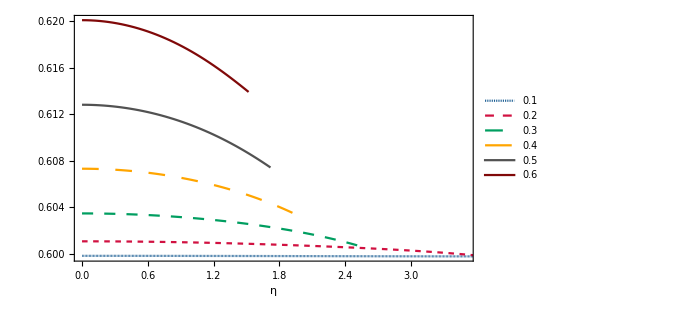

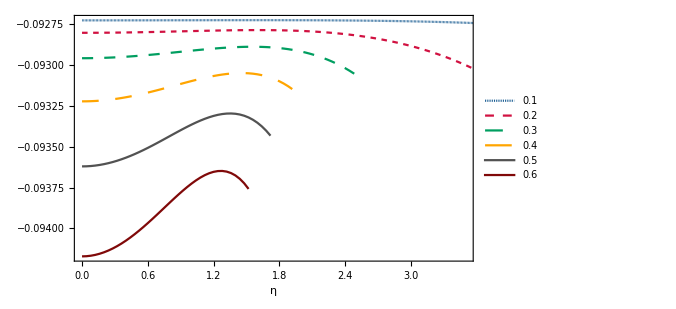

```mathematica
ListLinePlot[{Re[Tp[[1]]],Re[Tp[[2]]],Re[Tp[[3]]],Re[Tp[[4]]],Re[Tp[[5]]],Re[Tp[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[Tp[[1]]],Im[Tp[[2]]],Im[Tp[[3]]],Im[Tp[[4]]],Im[Tp[[5]]],Im[Tp[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100
(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100
(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100
(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100
```

0.0403728

-0.380562

1.00604

-0.556147

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tdp]-Im[Tda])[[k]][[j+1]][[1]]/(Abs[Im[Tda][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

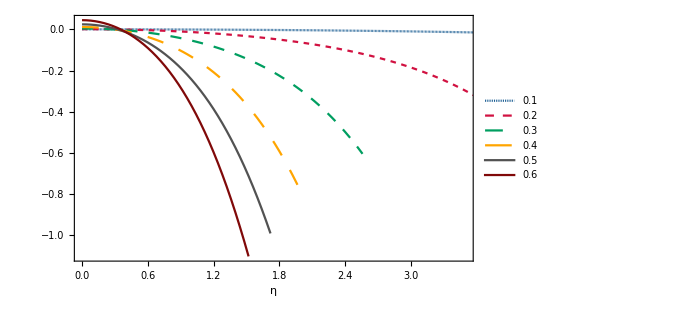

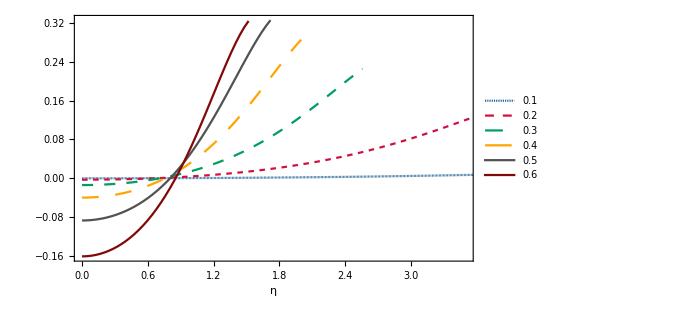

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.12,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
Max[Abs[(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100],Abs[(Max[Re[Tda[[2]]]]-Min[Re[Tda[[2]]]])/Min[Re[Tda[[2]]]]*100],Abs[(Max[Re[Tda[[3]]]]-Min[Re[Tda[[3]]]])/Min[Re[Tda[[3]]]]*100],Abs[(Max[Re[Tda[[4]]]]-Min[Re[Tda[[4]]]])/Min[Re[Tda[[4]]]]*100],Abs[(Max[Re[Tda[[5]]]]-Min[Re[Tda[[5]]]])/Min[Re[Tda[[5]]]]*100],Abs[(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100]]
Max[Abs[(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100],Abs[(Max[Im[Tda[[2]]]]-Min[Im[Tda[[2]]]])/Min[Im[Tda[[2]]]]*100],Abs[(Max[Im[Tda[[3]]]]-Min[Im[Tda[[3]]]])/Min[Im[Tda[[3]]]]*100],Abs[(Max[Im[Tda[[4]]]]-Min[Im[Tda[[4]]]])/Min[Im[Tda[[4]]]]*100],Abs[(Max[Im[Tda[[5]]]]-Min[Im[Tda[[5]]]])/Min[Im[Tda[[5]]]]*100],Abs[(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100]]
```

0.179107

0.419502

```mathematica
Max[Abs[(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100],Abs[(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100],Abs[(Max[Re[Tdp[[3]]]]-Min[Re[Tdp[[3]]]])/Min[Re[Tdp[[3]]]]*100],Abs[(Max[Re[Tdp[[4]]]]-Min[Re[Tdp[[4]]]])/Min[Re[Tdp[[4]]]]*100],Abs[(Max[Re[Tdp[[5]]]]-Min[Re[Tdp[[5]]]])/Min[Re[Tdp[[5]]]]*100],Abs[(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100],Abs[(Max[Im[Tdp[[2]]]]-Min[Im[Tdp[[2]]]])/Min[Im[Tdp[[2]]]]*100],Abs[(Max[Im[Tdp[[3]]]]-Min[Im[Tdp[[3]]]])/Min[Im[Tdp[[3]]]]*100],Abs[(Max[Im[Tdp[[4]]]]-Min[Im[Tdp[[4]]]])/Min[Im[Tdp[[4]]]]*100],Abs[(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100],Abs[(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100]]
```

1.00604

0.556147

## l=1 EM mode axial & polar

#### Axial modes

```mathematica
Ta1={{{0,0.2490496304059624-0.09259085005107087 ⅈ},{1/25+ⅈ/25,0.2490496312180845-0.0925908499521117 ⅈ},{2/25+(2 ⅈ)/25,0.24904963365537375-0.09259084965573051 ⅈ},{3/25+(3 ⅈ)/25,0.24904963772059124-0.09259084916341653 ⅈ},{4/25+(4 ⅈ)/25,0.2490496434183403-0.0925908484776511 ⅈ},{1/5+ⅈ/5,0.2490496507550664-0.09259084760190672 ⅈ},{6/25+(6 ⅈ)/25,0.24904965973905788-0.09259084654064599 ⅈ},{7/25+(7 ⅈ)/25,0.24904967038044656-0.09259084529931973 ⅈ},{8/25+(8 ⅈ)/25,0.24904968269120947-0.0925908438843652 ⅈ},{9/25+(9 ⅈ)/25,0.2490496966851694-0.09259084230320351 ⅈ},{2/5+(2 ⅈ)/5,0.24904971237799722-0.09259084056423714 ⅈ},{11/25+(11 ⅈ)/25,0.24904972978721296-0.0925908386768467 ⅈ},{12/25+(12 ⅈ)/25,0.24904974893218826-0.09259083665138741 ⅈ},{13/25+(13 ⅈ)/25,0.24904976983414814-0.09259083449918536 ⅈ},{14/25+(14 ⅈ)/25,0.24904979251617357-0.09259083223253319 ⅈ},{3/5+(3 ⅈ)/5,0.24904981700320383-0.09259082986468567 ⅈ},{16/25+(16 ⅈ)/25,0.24904984332203964-0.09259082740985473 ⅈ},{17/25+(17 ⅈ)/25,0.24904987150134528-0.092590824883204 ⅈ},{18/25+(18 ⅈ)/25,0.24904990157164997-0.09259082230084521 ⅈ},{19/25+(19 ⅈ)/25,0.24904993356536131-0.09259081967982398 ⅈ},{4/5+(4 ⅈ)/5,0.24904996751675326-0.09259081703812548 ⅈ},{21/25+(21 ⅈ)/25,0.24905000346197997-0.09259081439465955 ⅈ},{22/25+(22 ⅈ)/25,0.24905004143907747-0.09259081176925553 ⅈ},{23/25+(23 ⅈ)/25,0.2490500814879674-0.09259080918265454 ⅈ},{24/25+(24 ⅈ)/25,0.24905012365046145-0.09259080665650156 ⅈ},{1+ⅈ,0.24905016797026597-0.09259080421333699 ⅈ},{26/25+(26 ⅈ)/25,0.24905021449298642-0.09259080187658782 ⅈ},{27/25+(27 ⅈ)/25,0.24905026326613222-0.09259079967055846 ⅈ},{28/25+(28 ⅈ)/25,0.24905031433912184-0.09259079762042137 ⅈ},{29/25+(29 ⅈ)/25,0.24905036776328796-0.09259079575220659 ⅈ},{6/5+(6 ⅈ)/5,0.24905042359188273-0.09259079409279183 ⅈ},{31/25+(31 ⅈ)/25,0.2490504818800835-0.09259079266989136 ⅈ},{32/25+(32 ⅈ)/25,0.2490505426849983-0.0925907915120449 ⅈ},{33/25+(33 ⅈ)/25,0.2490506060656719-0.09259079064860601 ⅈ},{34/25+(34 ⅈ)/25,0.24905067208309162-0.09259079010972988 ⅈ},{7/5+(7 ⅈ)/5,0.24905074080019377-0.09259078992636108 ⅈ},{36/25+(36 ⅈ)/25,0.2490508122818698-0.09259079013022045 ⅈ},{37/25+(37 ⅈ)/25,0.24905088659497293-0.09259079075379187 ⅈ},{38/25+(38 ⅈ)/25,0.24905096380832464-0.0925907918303085 ⅈ},{39/25+(39 ⅈ)/25,0.24905104399272174-0.0925907933937384 ⅈ},{8/5+(8 ⅈ)/5,0.249051127220943-0.09259079547877015 ⅈ},{41/25+(41 ⅈ)/25,0.2490512135677565-0.09259079812079747 ⅈ},{42/25+(42 ⅈ)/25,0.24905130310992665-0.09259080135590386 ⅈ},{43/25+(43 ⅈ)/25,0.24905139592622166-0.09259080522084649 ⅈ},{44/25+(44 ⅈ)/25,0.24905149209742106-0.09259080975303974 ⅈ},{9/5+(9 ⅈ)/5,0.24905159170632307-0.09259081499053827 ⅈ},{46/25+(46 ⅈ)/25,0.2490516948377527-0.09259082097201964 ⅈ},{47/25+(47 ⅈ)/25,0.2490518015785692-0.09259082773676627 ⅈ},{48/25+(48 ⅈ)/25,0.24905191201767432-0.09259083532464739 ⅈ},{49/25+(49 ⅈ)/25,0.24905202624602013-0.09259084377609979 ⅈ},{2+2 ⅈ,0.24905214435661738-0.09259085313210877 ⅈ},{51/25+(51 ⅈ)/25,0.2490522664445436-0.09259086343418811 ⅈ},{52/25+(52 ⅈ)/25,0.24905239260695144-0.09259087472435991 ⅈ},{53/25+(53 ⅈ)/25,0.24905252294307725-0.09259088704513356 ⅈ},{54/25+(54 ⅈ)/25,0.2490526575542494-0.09259090043948441 ⅈ},{11/5+(11 ⅈ)/5,0.24905279654389695-0.09259091495083203 ⅈ},{56/25+(56 ⅈ)/25,0.24905294001755823-0.09259093062301763 ⅈ},{57/25+(57 ⅈ)/25,0.24905308808288967-0.09259094750028103 ⅈ},{58/25+(58 ⅈ)/25,0.24905324084967434-0.09259096562723755 ⅈ},{59/25+(59 ⅈ)/25,0.24905339842983093-0.09259098504885363 ⅈ},{12/5+(12 ⅈ)/5,0.2490535609374225-0.09259100581042237 ⅈ},{61/25+(61 ⅈ)/25,0.24905372848866536-0.09259102795753853 ⅈ},{62/25+(62 ⅈ)/25,0.24905390120193804-0.09259105153607257 ⅈ},{63/25+(63 ⅈ)/25,0.24905407919778996-0.09259107659214463 ⅈ},{64/25+(64 ⅈ)/25,0.24905426259895072-0.09259110317209762 ⅈ},{13/5+(13 ⅈ)/5,0.2490544515303387-0.0925911313224698 ⅈ},{66/25+(66 ⅈ)/25,0.24905464611907016-0.09259116108996673 ⅈ},{67/25+(67 ⅈ)/25,0.24905484649446794-0.09259119252143286 ⅈ},{68/25+(68 ⅈ)/25,0.2490550527880706-0.09259122566382197 ⅈ},{69/25+(69 ⅈ)/25,0.2490552651336411-0.09259126056416779 ⅈ},{14/5+(14 ⅈ)/5,0.2490554836671755-0.09259129726955326 ⅈ},{71/25+(71 ⅈ)/25,0.24905570852691192-0.09259133582707964 ⅈ},{72/25+(72 ⅈ)/25,0.24905593985333901-0.0925913762838349 ⅈ},{73/25+(73 ⅈ)/25,0.2490561777892048-0.09259141868686117 ⅈ},{74/25+(74 ⅈ)/25,0.24905642247952495-0.09259146308312204 ⅈ},{3+3 ⅈ,0.24905667407159132-0.09259150951946882 ⅈ},{76/25+(76 ⅈ)/25,0.24905693271498033-0.09259155804260633 ⅈ},{77/25+(77 ⅈ)/25,0.249057198561561-0.09259160869905801 ⅈ},{78/25+(78 ⅈ)/25,0.24905747176550325-0.0925916615351303 ⅈ},{79/25+(79 ⅈ)/25,0.24905775248328563-0.09259171659687639 ⅈ},{16/5+(16 ⅈ)/5,0.24905804087370326-0.09259177393005916 ⅈ},{81/25+(81 ⅈ)/25,0.24905833709787528-0.09259183358011377 ⅈ},{82/25+(82 ⅈ)/25,0.2490586413192525-0.09259189559210908 ⅈ},{83/25+(83 ⅈ)/25,0.24905895370362446-0.09259196001070877 ⅈ},{84/25+(84 ⅈ)/25,0.2490592744191265-0.09259202688013148 ⅈ},{17/5+(17 ⅈ)/5,0.24905960363624677-0.09259209624411024 ⅈ},{86/25+(86 ⅈ)/25,0.24905994152783248-0.09259216814585167 ⅈ},{87/25+(87 ⅈ)/25,0.24906028826909654-0.09259224262799341 ⅈ},{88/25+(88 ⅈ)/25,0.24906064403762354-0.09259231973256206 ⅈ},{89/25+(89 ⅈ)/25,0.24906100901337544-0.09259239950092922 ⅈ},{18/5+(18 ⅈ)/5,0.24906138337869715-0.09259248197376775 ⅈ},{91/25+(91 ⅈ)/25,0.24906176731832186-0.09259256719100645 ⅈ},{92/25+(92 ⅈ)/25,0.24906216101937553-0.09259265519178464 ⅈ},{93/25+(93 ⅈ)/25,0.24906256467138188-0.09259274601440545 ⅈ},{94/25+(94 ⅈ)/25,0.24906297846626602-0.09259283969628869 ⅈ},{19/5+(19 ⅈ)/5,0.24906340259835863-0.09259293627392277 ⅈ},{96/25+(96 ⅈ)/25,0.24906383726439918-0.09259303578281573 ⅈ},{97/25+(97 ⅈ)/25,0.24906428266353875-0.09259313825744579 ⅈ},{98/25+(98 ⅈ)/25,0.24906473899734283-0.09259324373121071 ⅈ},{99/25+(99 ⅈ)/25,0.24906520646979302-0.09259335223637669 ⅈ},{4+4 ⅈ,0.24906568528728887-0.09259346380402608 ⅈ},{101/25+(101 ⅈ)/25,0.24906617565864886-0.09259357846400469 ⅈ},{102/25+(102 ⅈ)/25,0.24906667779511088-0.09259369624486795 ⅈ},{103/25+(103 ⅈ)/25,0.24906719191033228-0.09259381717382638 ⅈ},{104/25+(104 ⅈ)/25,0.24906771822038948-0.09259394127669009 ⅈ},{21/5+(21 ⅈ)/5,0.24906825694377654-0.09259406857781279 ⅈ},{106/25+(106 ⅈ)/25,0.2490688083014035-0.09259419910003433 ⅈ},{107/25+(107 ⅈ)/25,0.24906937251659417-0.09259433286462317 ⅈ},{108/25+(108 ⅈ)/25,0.24906994981508288-0.09259446989121725 ⅈ},{109/25+(109 ⅈ)/25,0.24907054042501067-0.0925946101977646 ⅈ},{22/5+(22 ⅈ)/5,0.2490711445769212-0.09259475380046267 ⅈ},{111/25+(111 ⅈ)/25,0.24907176250375515-0.09259490071369703 ⅈ},{112/25+(112 ⅈ)/25,0.24907239444084459-0.09259505094997918 ⅈ},{113/25+(113 ⅈ)/25,0.24907304062590607-0.09259520451988332 ⅈ},{114/25+(114 ⅈ)/25,0.2490737012990332-0.09259536143198253 ⅈ},{23/5+(23 ⅈ)/5,0.2490743767026881-0.09259552169278389 ⅈ},{116/25+(116 ⅈ)/25,0.24907506708169228-0.09259568530666273 ⅈ},{117/25+(117 ⅈ)/25,0.24907577268321654-0.0925958522757961 ⅈ},{118/25+(118 ⅈ)/25,0.24907649375676957-0.09259602260009532 ⅈ},{119/25+(119 ⅈ)/25,0.2490772305541862-0.09259619627713762 ⅈ},{24/5+(24 ⅈ)/5,0.24907798332961412-0.09259637330209708 ⅈ},{121/25+(121 ⅈ)/25,0.24907875233949997-0.09259655366767439 ⅈ},{122/25+(122 ⅈ)/25,0.24907953784257414-0.0925967373640261 ⅈ},{123/25+(123 ⅈ)/25,0.24908034009983454-0.09259692437869274 ⅈ},{124/25+(124 ⅈ)/25,0.24908115937452918-0.09259711469652629 ⅈ},{5+5 ⅈ,0.24908199593213776-0.0925973082996166 ⅈ},{126/25+(126 ⅈ)/25,0.2490828500403519-0.09259750516721707 ⅈ},{127/25+(127 ⅈ)/25,0.2490837219690543-0.0925977052756695 ⅈ},{128/25+(128 ⅈ)/25,0.2490846119902964-0.09259790859832805 ⅈ},{129/25+(129 ⅈ)/25,0.24908552037827505-0.09259811510548235 ⅈ},{26/5+(26 ⅈ)/5,0.24908644740930766-0.09259832476428 ⅈ},{131/25+(131 ⅈ)/25,0.2490873933618058-0.09259853753864773 ⅈ},{132/25+(132 ⅈ)/25,0.24908835851624775-0.09259875338921256 ⅈ},{133/25+(133 ⅈ)/25,0.24908934315514955-0.09259897227322139 ⅈ},{134/25+(134 ⅈ)/25,0.24909034756303422-0.09259919414446022 ⅈ},{27/5+(27 ⅈ)/5,0.24909137202639978-0.09259941895317254 ⅈ},{136/25+(136 ⅈ)/25,0.24909241683368563-0.0925996466459769 ⅈ},{137/25+(137 ⅈ)/25,0.24909348227523714-0.09259987716578379 ⅈ},{138/25+(138 ⅈ)/25,0.24909456864326893-0.09260011045171182 ⅈ},{139/25+(139 ⅈ)/25,0.24909567623182613-0.09260034643900297 ⅈ},{28/5+(28 ⅈ)/5,0.24909680533674408-0.09260058505893745 ⅈ},{141/25+(141 ⅈ)/25,0.2490979562556061-0.09260082623874785 ⅈ},{142/25+(142 ⅈ)/25,0.24909912928769973-0.0926010699015322 ⅈ},{143/25+(143 ⅈ)/25,0.24910032473397076-0.09260131596616708 ⅈ},{144/25+(144 ⅈ)/25,0.24910154289697553-0.09260156434721944 ⅈ},{29/5+(29 ⅈ)/5,0.2491027840808312-0.09260181495485856 ⅈ},{146/25+(146 ⅈ)/25,0.2491040485911643-0.09260206769476646 ⅈ},{147/25+(147 ⅈ)/25,0.24910533673505653-0.09260232246804902 ⅈ},{148/25+(148 ⅈ)/25,0.2491066488209893-0.09260257917114531 ⅈ},{149/25+(149 ⅈ)/25,0.2491079851587857-0.09260283769573743 ⅈ},{6+6 ⅈ,0.24910934605955024-0.09260309792865935 ⅈ},{151/25+(151 ⅈ)/25,0.2491107318356065-0.09260335975180553 ⅈ},{152/25+(152 ⅈ)/25,0.24911214280043237-0.09260362304203913 ⅈ},{153/25+(153 ⅈ)/25,0.24911357926859318-0.09260388767109988 ⅈ},{154/25+(154 ⅈ)/25,0.24911504155567213-0.09260415350551154 ⅈ},{31/5+(31 ⅈ)/5,0.24911652997819872-0.09260442040648928 ⅈ},{156/25+(156 ⅈ)/25,0.24911804485357414-0.09260468822984658 ⅈ},{157/25+(157 ⅈ)/25,0.24911958649999472-0.09260495682590215 ⅈ},{158/25+(158 ⅈ)/25,0.2491211552363724-0.09260522603938669 ⅈ},{159/25+(159 ⅈ)/25,0.24912275138225273-0.09260549570934934 ⅈ},{32/5+(32 ⅈ)/5,0.24912437525773024-0.09260576566906442 ⅈ},{161/25+(161 ⅈ)/25,0.24912602718336097-0.09260603574593777 ⅈ},{162/25+(162 ⅈ)/25,0.24912770748007237-0.09260630576141346 ⅈ},{163/25+(163 ⅈ)/25,0.2491294164690703-0.09260657553088054 ⅈ},{164/25+(164 ⅈ)/25,0.24913115447174305-0.09260684486357991 ⅈ},{33/5+(33 ⅈ)/5,0.24913292180956284-0.09260711356251135 ⅈ},{166/25+(166 ⅈ)/25,0.2491347188039839-0.09260738142434084 ⅈ},{167/25+(167 ⅈ)/25,0.24913654577633784-0.09260764823930855 ⅈ},{168/25+(168 ⅈ)/25,0.2491384030477258-0.09260791379113668 ⅈ},{169/25+(169 ⅈ)/25,0.2491402909389076-0.09260817785693834 ⅈ},{34/5+(34 ⅈ)/5,0.24914220977018786-0.09260844020712652 ⅈ},{171/25+(171 ⅈ)/25,0.24914415986129862-0.09260870060532403 ⅈ},{172/25+(172 ⅈ)/25,0.24914614153127887-0.09260895880827402 ⅈ},{173/25+(173 ⅈ)/25,0.2491481550983511-0.09260921456575112 ⅈ},{174/25+(174 ⅈ)/25,0.24915020087979386-0.09260946762047374 ⅈ},{7+7 ⅈ,0.24915227919181182-0.0926097177080171 ⅈ},{176/25+(176 ⅈ)/25,0.24915439034940157-0.09260996455672732 ⅈ},{177/25+(177 ⅈ)/25,0.24915653466621474-0.09261020788763674 ⅈ},{178/25+(178 ⅈ)/25,0.24915871245441684-0.09261044741438024 ⅈ}},{{0,0.25139375215294224-0.0928978901961061 ⅈ},{1/25+ⅈ/25,0.2513937649692252-0.09289788862895526 ⅈ},{2/25+(2 ⅈ)/25,0.2513938034320809-0.09289788393358658 ⅈ},{3/25+(3 ⅈ)/25,0.2513938675834026-0.09289787612826265 ⅈ},{4/25+(4 ⅈ)/25,0.25139395749305343-0.09289786524337892 ⅈ},{1/5+ⅈ/5,0.2513940732588807-0.09289785132140826 ⅈ},{6/25+(6 ⅈ)/25,0.25139421500675513-0.0928978344168201 ⅈ},{7/25+(7 ⅈ)/25,0.25139438289062077-0.0928978145959764 ⅈ},{8/25+(8 ⅈ)/25,0.2513945770925562-0.09289779193700387 ⅈ},{9/25+(9 ⅈ)/25,0.25139479782284596-0.09289776652964316 ⅈ},{2/5+(2 ⅈ)/5,0.2513950453200634-0.0928977384750739 ⅈ},{11/25+(11 ⅈ)/25,0.25139531985116337-0.09289770788571602 ⅈ},{12/25+(12 ⅈ)/25,0.25139562171158564-0.09289767488500668 ⅈ},{13/25+(13 ⅈ)/25,0.2513959512253683-0.09289763960715312 ⅈ},{14/25+(14 ⅈ)/25,0.2513963087452709-0.09289760219686047 ⅈ},{3/5+(3 ⅈ)/5,0.2513966946529077-0.09289756280903458 ⅈ},{16/25+(16 ⅈ)/25,0.2513971093588895-0.09289752160845943 ⅈ},{17/25+(17 ⅈ)/25,0.25139755330297514-0.09289747876944911 ⅈ},{18/25+(18 ⅈ)/25,0.25139802695423147-0.09289743447547304 ⅈ},{19/25+(19 ⅈ)/25,0.25139853081120145-0.09289738891875512 ⅈ},{4/5+(4 ⅈ)/5,0.2513990654020804-0.09289734229984559 ⅈ},{21/25+(21 ⅈ)/25,0.25139963128489967-0.09289729482716547 ⅈ},{22/25+(22 ⅈ)/25,0.2514002290477171-0.09289724671652295 ⅈ},{23/25+(23 ⅈ)/25,0.2514008593088143-0.09289719819060124 ⅈ},{24/25+(24 ⅈ)/25,0.2514015227168998-0.0928971494784173 ⅈ},{1+ⅈ,0.2514022199513174-0.09289710081475105 ⅈ},{26/25+(26 ⅈ)/25,0.2514029517222595-0.09289705243954406 ⅈ},{27/25+(27 ⅈ)/25,0.2514037187709846-0.0928970045972677 ⅈ},{28/25+(28 ⅈ)/25,0.251404521870038-0.09289695753625933 ⅈ},{29/25+(29 ⅈ)/25,0.25140536182347517-0.09289691150802676 ⅈ},{6/5+(6 ⅈ)/5,0.25140623946708757-0.09289686676651952 ⅈ},{31/25+(31 ⅈ)/25,0.25140715566862853-0.09289682356736662 ⅈ},{32/25+(32 ⅈ)/25,0.25140811132804014-0.09289678216708017 ⅈ},{33/25+(33 ⅈ)/25,0.25140910737767896-0.09289674282222378 ⅈ},{34/25+(34 ⅈ)/25,0.2514101447825399-0.09289670578854521 ⅈ},{7/5+(7 ⅈ)/5,0.25141122454047754-0.0928966713200726 ⅈ},{36/25+(36 ⅈ)/25,0.251412347682423-0.09289663966817328 ⅈ},{37/25+(37 ⅈ)/25,0.251413515272596-0.09289661108057436 ⅈ},{38/25+(38 ⅈ)/25,0.25141472840871026-0.09289658580034467 ⅈ},{39/25+(39 ⅈ)/25,0.2514159882221716-0.09289656406483668 ⅈ},{8/5+(8 ⅈ)/5,0.251417295878266-0.09289654610458813 ⅈ},{41/25+(41 ⅈ)/25,0.25141865257633805-0.09289653214218226 ⅈ},{42/25+(42 ⅈ)/25,0.25142005954995633-0.09289652239106577 ⅈ},{43/25+(43 ⅈ)/25,0.25142151806706575-0.09289651705432406 ⅈ},{44/25+(44 ⅈ)/25,0.2514230294301236-0.09289651632341255 ⅈ},{9/5+(9 ⅈ)/5,0.25142459497621905-0.09289652037684351 ⅈ},{46/25+(46 ⅈ)/25,0.25142621607717247-0.09289652937882767 ⅈ},{47/25+(47 ⅈ)/25,0.2514278941396143-0.09289654347786966 ⅈ},{48/25+(48 ⅈ)/25,0.25142963060504014-0.09289656280531683 ⅈ},{49/25+(49 ⅈ)/25,0.2514314269498408-0.09289658747386033 ⅈ},{2+2 ⅈ,0.2514332846853034-0.09289661757598837 ⅈ},{51/25+(51 ⅈ)/25,0.25143520535758374-0.09289665318239045 ⅈ},{52/25+(52 ⅈ)/25,0.25143719054764446-0.09289669434031217 ⅈ},{53/25+(53 ⅈ)/25,0.25143924187115885-0.09289674107186056 ⅈ},{54/25+(54 ⅈ)/25,0.2514413609783756-0.09289679337225838 ⅈ},{11/5+(11 ⅈ)/5,0.2514435495539434-0.09289685120804825 ⅈ},{56/25+(56 ⅈ)/25,0.25144580931669064-0.09289691451524514 ⅈ},{57/25+(57 ⅈ)/25,0.2514481420193582-0.09289698319743782 ⅈ},{58/25+(58 ⅈ)/25,0.25145054944828227-0.09289705712383842 ⅈ},{59/25+(59 ⅈ)/25,0.2514530334230223-0.09289713612728047 ⅈ},{12/5+(12 ⅈ)/5,0.2514555957959324-0.09289722000216537 ⅈ},{61/25+(61 ⅈ)/25,0.2514582384516716-0.0928973085023571 ⅈ},{62/25+(62 ⅈ)/25,0.25146096330664847-0.09289740133902608 ⅈ},{63/25+(63 ⅈ)/25,0.25146377230839795-0.09289749817844174 ⅈ},{64/25+(64 ⅈ)/25,0.2514666674348846-0.09289759863971517 ⅈ},{13/5+(13 ⅈ)/5,0.25146965069372884-0.09289770229249221 ⅈ},{66/25+(66 ⅈ)/25,0.251472724121352-0.09289780865459761 ⅈ},{67/25+(67 ⅈ)/25,0.2514758897820348-0.09289791718963207 ⅈ},{68/25+(68 ⅈ)/25,0.2514791497668855-0.09289802730452269 ⅈ},{69/25+(69 ⅈ)/25,0.2514825061927128-0.09289813834702865 ⅈ},{14/5+(14 ⅈ)/5,0.2514859612007977-0.0928982496032043 ⅈ},{71/25+(71 ⅈ)/25,0.2514895169555607-0.09289836029482086 ⅈ},{72/25+(72 ⅈ)/25,0.25149317564311796-0.09289846957674962 ⅈ},{73/25+(73 ⅈ)/25,0.25149693946972146-0.09289857653430898 ⅈ},{74/25+(74 ⅈ)/25,0.2515008106600784-0.09289868018057822 ⅈ},{3+3 ⅈ,0.25150479145554305-0.09289877945368123 ⅈ},{76/25+(76 ⅈ)/25,0.2515088841121772-0.09289887321404366 ⅈ},{77/25+(77 ⅈ)/25,0.25151309089867147-0.09289896024162757 ⅈ},{78/25+(78 ⅈ)/25,0.25151741409412337-0.09289903923314788 ⅈ},{79/25+(79 ⅈ)/25,0.2515218559856659-0.09289910879927489 ⅈ},{16/5+(16 ⅈ)/5,0.25152641886594007-0.0928991674618288 ⅈ},{81/25+(81 ⅈ)/25,0.2515311050304068-0.09289921365097105 ⅈ},{82/25+(82 ⅈ)/25,0.25153591677449083-0.09289924570239906 ⅈ},{83/25+(83 ⅈ)/25,0.25154085639055235-0.09289926185455076 ⅈ},{84/25+(84 ⅈ)/25,0.2515459261646792-0.09289926024582593 ⅈ},{17/5+(17 ⅈ)/5,0.25155112837329513-0.09289923891183204 ⅈ},{86/25+(86 ⅈ)/25,0.25155646527957737-0.09289919578266298 ⅈ},{87/25+(87 ⅈ)/25,0.2515619391296787-0.09289912868021899 ⅈ},{88/25+(88 ⅈ)/25,0.2515675521487491-0.09289903531557774 ⅈ},{89/25+(89 ⅈ)/25,0.2515733065367508-0.09289891328642579 ⅈ},{18/5+(18 ⅈ)/5,0.2515792044640631-0.09289876007456241 ⅈ},{91/25+(91 ⅈ)/25,0.25158524806687127-0.09289857304348521 ⅈ}},{{0,0.2552518819430734-0.0934019797296957 ⅈ},{1/25+ⅈ/25,0.2552519453820567-0.09340197194147158 ⅈ},{2/25+(2 ⅈ)/25,0.2552521357638146-0.09340194859303516 ⅈ},{3/25+(3 ⅈ)/25,0.25525245328218366-0.0934019097330428 ⅈ},{4/25+(4 ⅈ)/25,0.25525289826048597-0.09340185544214426 ⅈ},{1/5+ⅈ/5,0.25525347115169916-0.0934017858323425 ⅈ},{6/25+(6 ⅈ)/25,0.2552541725387798-0.09340170104608435 ⅈ},{7/25+(7 ⅈ)/25,0.25525500313507693-0.09340160125508769 ⅈ},{8/25+(8 ⅈ)/25,0.2552559637848322-0.09340148665890223 ⅈ},{9/25+(9 ⅈ)/25,0.2552570554637631-0.0934013574832007 ⅈ},{2/5+(2 ⅈ)/5,0.2552582792797271-0.09340121397779613 ⅈ},{11/25+(11 ⅈ)/25,0.25525963647346067-0.09340105641438094 ⅈ},{12/25+(12 ⅈ)/25,0.2552611284193891-0.09340088508398232 ⅈ},{13/25+(13 ⅈ)/25,0.25526275662650144-0.09340070029412845 ⅈ},{14/25+(14 ⅈ)/25,0.25526452273928335-0.0934005023657188 ⅈ},{3/5+(3 ⅈ)/5,0.25526642853870213-0.09340029162959185 ⅈ},{16/25+(16 ⅈ)/25,0.2552684759432334-0.09340006842278287 ⅈ},{17/25+(17 ⅈ)/25,0.25527066700992357-0.0933998330844633 ⅈ},{18/25+(18 ⅈ)/25,0.2552730039354756-0.09339958595155358 ⅈ},{19/25+(19 ⅈ)/25,0.2552754890573488-0.09339932735400047 ⅈ},{4/5+(4 ⅈ)/5,0.2552781248548602-0.09339905760970899 ⅈ},{21/25+(21 ⅈ)/25,0.255280913950274-0.09339877701911978 ⅈ},{22/25+(22 ⅈ)/25,0.25528385910986623-0.09339848585942093 ⅈ},{23/25+(23 ⅈ)/25,0.25528696324494765-0.09339818437838394 ⅈ},{24/25+(24 ⅈ)/25,0.2552902294128291-0.09339787278781331 ⅈ},{1+ⅈ,0.25529366081771016-0.09339755125659781 ⅈ},{26/25+(26 ⅈ)/25,0.2552972608114727-0.09339721990335287 ⅈ},{27/25+(27 ⅈ)/25,0.2553010328943555-0.09339687878864303 ⅈ},{28/25+(28 ⅈ)/25,0.2553049807154905-0.09339652790677029 ⅈ},{29/25+(29 ⅈ)/25,0.2553091080732711-0.09339616717712214 ⅈ},{6/5+(6 ⅈ)/5,0.25531341891552933-0.09339579643506303 ⅈ},{31/25+(31 ⅈ)/25,0.2553179173394919-0.09339541542236113 ⅈ},{32/25+(32 ⅈ)/25,0.25532260759148273-0.09339502377713958 ⅈ},{33/25+(33 ⅈ)/25,0.25532749406634087-0.09339462102334202 ⅈ},{34/25+(34 ⅈ)/25,0.25533258130651565-0.09339420655970339 ⅈ},{7/5+(7 ⅈ)/5,0.2553378740008032-0.0933937796482182 ⅈ},{36/25+(36 ⅈ)/25,0.25534337698268206-0.09339333940209835 ⅈ},{37/25+(37 ⅈ)/25,0.2553490952282045-0.09339288477321624 ⅈ},{38/25+(38 ⅈ)/25,0.25535503385339803-0.09339241453902716 ⅈ},{39/25+(39 ⅈ)/25,0.25536119811112706-0.09339192728897037 ⅈ},{8/5+(8 ⅈ)/5,0.25536759338736353-0.09339142141034779 ⅈ},{41/25+(41 ⅈ)/25,0.25537422519680936-0.0933908950736827 ⅈ},{42/25+(42 ⅈ)/25,0.2553810991778151-0.09339034621756408 ⅈ},{43/25+(43 ⅈ)/25,0.2553882210865305-0.09338977253298442 ⅈ},{44/25+(44 ⅈ)/25,0.2553955967902239-0.09338917144718295 ⅈ},{9/5+(9 ⅈ)/5,0.2554032322597024-0.09338854010701042 ⅈ},{46/25+(46 ⅈ)/25,0.2554111335607601-0.09338787536183603 ⅈ},{47/25+(47 ⅈ)/25,0.25541930684458264-0.09338717374602147 ⅈ},{48/25+(48 ⅈ)/25,0.25542775833702813-0.09338643146099354 ⅈ},{49/25+(49 ⅈ)/25,0.2554364943267064-0.09338564435695242 ⅈ},{2+2 ⅈ,0.25544552115177244-0.09338480791425947 ⅈ},{51/25+(51 ⅈ)/25,0.25545484518534917-0.09338391722455591 ⅈ},{52/25+(52 ⅈ)/25,0.25546447281949203-0.09338296697167163 ⅈ},{53/25+(53 ⅈ)/25,0.2554744104476067-0.09338195141239275 ⅈ},{54/25+(54 ⅈ)/25,0.2554846644452288-0.09338086435716486 ⅈ},{11/5+(11 ⅈ)/5,0.25549524114907557-0.09337969915082071 ⅈ},{56/25+(56 ⅈ)/25,0.2555061468342772-0.09337844865343069 ⅈ},{57/25+(57 ⅈ)/25,0.25551738768969956-0.09337710522138701 ⅈ},{58/25+(58 ⅈ)/25,0.255528969791268-0.09337566068884523 ⅈ},{59/25+(59 ⅈ)/25,0.2555408990732072-0.0933741063496592 ⅈ},{12/5+(12 ⅈ)/5,0.2555531812971159-0.09337243293996073 ⅈ},{61/25+(61 ⅈ)/25,0.2555658220187993-0.09337063062154877 ⅈ},{62/25+(62 ⅈ)/25,0.2555788265527893-0.09336868896626953 ⅈ},{63/25+(63 ⅈ)/25,0.25559219993449245-0.09336659694158383 ⅈ},{64/25+(64 ⅈ)/25,0.25560594687991406-0.09336434289753474 ⅈ}},{{0,0.26055483493224846-0.09409233948701948 ⅈ},{1/25+ⅈ/25,0.260555029387937-0.09409231556290744 ⅈ},{2/25+(2 ⅈ)/25,0.26055561293499824-0.09409224378379556 ⅈ},{3/25+(3 ⅈ)/25,0.2605565861116221-0.0940921241288855 ⅈ},{4/25+(4 ⅈ)/25,0.26055794981560415-0.0940919565611036 ⅈ},{1/5+ⅈ/5,0.2605597053048742-0.09409174102356116 ⅈ},{6/25+(6 ⅈ)/25,0.26056185419848915-0.09409147743454738 ⅈ},{7/25+(7 ⅈ)/25,0.2605643984778761-0.09409116568106084 ⅈ},{8/25+(8 ⅈ)/25,0.2605673404883008-0.09409080561085754 ⅈ},{9/25+(9 ⅈ)/25,0.26057068294052843-0.09409039702298687 ⅈ},{2/5+(2 ⅈ)/5,0.2605744289126406-0.09408993965678338 ⅈ},{11/25+(11 ⅈ)/25,0.2605785818519614-0.09408943317927765 ⅈ},{12/25+(12 ⅈ)/25,0.26058314557704154-0.09408887717098366 ⅈ},{13/25+(13 ⅈ)/25,0.26058812427963923-0.09408827111001762 ⅈ},{14/25+(14 ⅈ)/25,0.2605935225266298-0.0940876143544978 ⅈ},{3/5+(3 ⅈ)/5,0.2605993452617658-0.0940869061231718 ⅈ},{16/25+(16 ⅈ)/25,0.2606055978072-0.09408614547421419 ⅈ},{17/25+(17 ⅈ)/25,0.26061228586467294-0.09408533128213493 ⅈ},{18/25+(18 ⅈ)/25,0.26061941551625534-0.09408446221273543 ⅈ},{19/25+(19 ⅈ)/25,0.2606269932245238-0.09408353669604906 ⅈ},{4/5+(4 ⅈ)/5,0.2606350258320339-0.09408255289720047 ⅈ},{21/25+(21 ⅈ)/25,0.2606435205599408-0.09408150868511844 ⅈ},{22/25+(22 ⅈ)/25,0.2606524850056038-0.09408040159903806 ⅈ},{23/25+(23 ⅈ)/25,0.26066192713899117-0.09407922881272938 ⅈ},{24/25+(24 ⅈ)/25,0.2606718552976874-0.09407798709639371 ⅈ},{1+ⅈ,0.2606822781802838-0.09407667277617314 ⅈ},{26/25+(26 ⅈ)/25,0.2606932048379151-0.09407528169122581 ⅈ},{27/25+(27 ⅈ)/25,0.2607046446636758-0.09407380914832761 ⅈ},{28/25+(28 ⅈ)/25,0.260716607379653-0.09407224987397333 ⅈ},{29/25+(29 ⅈ)/25,0.2607291030212371-0.09407059796396197 ⅈ},{6/5+(6 ⅈ)/5,0.2607421419184116-0.09406884683046925 ⅈ},{31/25+(31 ⅈ)/25,0.2607557346736463-0.09406698914662982 ⅈ},{32/25+(32 ⅈ)/25,0.26076989213601603-0.09406501678867474 ⅈ},{33/25+(33 ⅈ)/25,0.26078462537113417-0.0940629207756986 ⅈ},{34/25+(34 ⅈ)/25,0.2607999456264629-0.09406069120716276 ⅈ},{7/5+(7 ⅈ)/5,0.2608158642915348-0.09405831719827897 ⅈ},{36/25+(36 ⅈ)/25,0.26083239285259396-0.09405578681346063 ⅈ},{37/25+(37 ⅈ)/25,0.26084954284113915-0.09405308699807911 ⅈ},{38/25+(38 ⅈ)/25,0.2608673257758272-0.09405020350881764 ⅈ},{39/25+(39 ⅈ)/25,0.2608857530971743-0.09404712084298004 ⅈ},{8/5+(8 ⅈ)/5,0.2609048360944733-0.09404382216718067 ⅈ},{41/25+(41 ⅈ)/25,0.26092458582433453-0.09404028924592327 ⅈ},{42/25+(42 ⅈ)/25,0.2609450130202478-0.09403650237066208 ⅈ},{43/25+(43 ⅈ)/25,0.26096612799256363-0.09403244029003638 ⅈ},{44/25+(44 ⅈ)/25,0.26098794051830204-0.09402808014207516 ⅈ},{9/5+(9 ⅈ)/5,0.2610104597202148-0.09402339738928142 ⅈ},{46/25+(46 ⅈ)/25,0.26103369393456166-0.09401836575763145 ⅈ},{47/25+(47 ⅈ)/25,0.26105765056710717-0.09401295718065335 ⅈ},{48/25+(48 ⅈ)/25,0.26108233593691244-0.0940071417498897 ⅈ},{49/25+(49 ⅈ)/25,0.26110775510758-0.09400088767319327 ⅈ},{2+2 ⅈ,0.2611339117057215-0.09399416124245506 ⅈ}},{{0,0.2672128905246763-0.09495509910366037 ⅈ},{1/25+ⅈ/25,0.26721334760867-0.09495504300251882 ⅈ},{2/25+(2 ⅈ)/25,0.26721471923039175-0.09495487452382635 ⅈ},{3/25+(3 ⅈ)/25,0.26721700649458296-0.09495459313971229 ⅈ},{4/25+(4 ⅈ)/25,0.26722021124352796-0.09495419796152638 ⅈ},{1/5+ⅈ/5,0.26722433605696955-0.09495368772669499 ⅈ},{6/25+(6 ⅈ)/25,0.2672293842525172-0.09495306078015872 ⅈ},{7/25+(7 ⅈ)/25,0.2672353598859729-0.0949523150503652 ⅈ},{8/25+(8 ⅈ)/25,0.26724226775142423-0.09495144801971382 ⅈ},{9/25+(9 ⅈ)/25,0.26725011338091187-0.09495045668932571 ⅈ},{2/5+(2 ⅈ)/5,0.2672589030434437-0.09494933753799381 ⅈ},{11/25+(11 ⅈ)/25,0.26726864374307824-0.09494808647514838 ⅈ},{12/25+(12 ⅈ)/25,0.26727934321575786-0.09494669878765573 ⅈ},{13/25+(13 ⅈ)/25,0.2672910099245187-0.0949451690802552 ⅈ},{14/25+(14 ⅈ)/25,0.2673036530526483-0.09494349120942552 ⅈ},{3/5+(3 ⅈ)/5,0.26731728249430436-0.09494165821046521 ⅈ},{16/25+(16 ⅈ)/25,0.2673319088420382-0.09493966221756688 ⅈ},{17/25+(17 ⅈ)/25,0.26734754337059813-0.0949374943766666 ⅈ},{18/25+(18 ⅈ)/25,0.26736419801630695-0.09493514475085742 ⅈ},{19/25+(19 ⅈ)/25,0.26738188535122603-0.09493260221817004 ⅈ},{4/5+(4 ⅈ)/5,0.2674006185512232-0.09492985436154823 ⅈ},{21/25+(21 ⅈ)/25,0.2674204113569661-0.09492688735087933 ⅈ},{22/25+(22 ⅈ)/25,0.26744127802675416-0.0949236858169873 ⅈ},{23/25+(23 ⅈ)/25,0.26746323327998994-0.09492023271755606 ⅈ},{24/25+(24 ⅈ)/25,0.2674862922299722-0.0949165091950262 ⅈ},{1+ⅈ,0.2675104703045639-0.09491249442660687 ⅈ},{26/25+(26 ⅈ)/25,0.2675357831531614-0.09490816546666073 ⅈ},{27/25+(27 ⅈ)/25,0.26756224653825383-0.09490349708186292 ⅈ},{28/25+(28 ⅈ)/25,0.2675898762097279-0.0948984615797107 ⅈ},{29/25+(29 ⅈ)/25,0.2676186877599368-0.09489302863115773 ⅈ},{6/5+(6 ⅈ)/5,0.2676486964574252-0.09488716508839566 ⅈ},{31/25+(31 ⅈ)/25,0.26767991705707866-0.0948808347990802 ⅈ},{32/25+(32 ⅈ)/25,0.2677123635843642-0.0948739984186263 ⅈ},{33/25+(33 ⅈ)/25,0.26774604909124056-0.09486661322257058 ⅈ},{34/25+(34 ⅈ)/25,0.2677809853812685-0.09485863292142242 ⅈ},{7/5+(7 ⅈ)/5,0.2678171827014344-0.09485000748090518 ⅈ},{36/25+(36 ⅈ)/25,0.26785464939824066-0.09484068295102531 ⅈ},{37/25+(37 ⅈ)/25,0.2678933915357232-0.09483060130799983 ⅈ},{38/25+(38 ⅈ)/25,0.2679334124732397-0.09481970031372282 ⅈ},{39/25+(39 ⅈ)/25,0.26797471240116305-0.09480791339815357 ⅈ},{8/5+(8 ⅈ)/5,0.26801728783301987-0.09479516957075691 ⅈ},{41/25+(41 ⅈ)/25,0.26806113105316365-0.09478139336790893 ⅈ},{42/25+(42 ⅈ)/25,0.26810622951978963-0.09476650484398205 ⅈ},{43/25+(43 ⅈ)/25,0.26815256522400316-0.09475041961462242 ⅈ}},{{0,0.2751214923920958-0.09597421594005615 ⅈ},{1/25+ⅈ/25,0.2751223991114501-0.0959741057213872 ⅈ},{2/25+(2 ⅈ)/25,0.2751251198829316-0.095973774363574 ⅈ},{3/25+(3 ⅈ)/25,0.2751296565366428-0.0959732197547461 ⅈ},{4/25+(4 ⅈ)/25,0.27513601212057665-0.09597243834972212 ⅈ},{1/5+ⅈ/5,0.2751441908939373-0.09597142513216873 ⅈ},{6/25+(6 ⅈ)/25,0.27515419831857885-0.09597017356121049 ⅈ},{7/25+(7 ⅈ)/25,0.275166041047162-0.09596867550234604 ⅈ},{8/25+(8 ⅈ)/25,0.27517972690738834-0.09596692114235172 ⅈ},{9/25+(9 ⅈ)/25,0.2751952648815001-0.09596489888779343 ⅈ},{2/5+(2 ⅈ)/5,0.27521266508006337-0.09596259524671623 ⅈ},{11/25+(11 ⅈ)/25,0.2752319387088555-0.09595999469303933 ⅈ},{12/25+(12 ⅈ)/25,0.275253098027473-0.09595707951315478 ⅈ},{13/25+(13 ⅈ)/25,0.2752761562980435-0.09595382963421643 ⅈ},{14/25+(14 ⅈ)/25,0.2753011277221767-0.0959502224336101 ⅈ},{3/5+(3 ⅈ)/5,0.2753280273640155-0.09594623252912982 ⅈ},{16/25+(16 ⅈ)/25,0.2753568710569443-0.09594183154944387 ⅈ},{17/25+(17 ⅈ)/25,0.27538767529118746-0.09593698788453293 ⅈ},{18/25+(18 ⅈ)/25,0.2754204570791739-0.09593166641592353 ⅈ},{19/25+(19 ⅈ)/25,0.27545523379515746-0.09592582822673441 ⅈ},{4/5+(4 ⅈ)/5,0.27549202298517433-0.09591943029181031 ⅈ},{21/25+(21 ⅈ)/25,0.27553084214298035-0.09591242514854968 ⅈ},{22/25+(22 ⅈ)/25,0.2755717084471528-0.095904760549454 ⅈ},{23/25+(23 ⅈ)/25,0.27561463845407114-0.09589637909794688 ⅈ},{24/25+(24 ⅈ)/25,0.27565964774101154-0.09588721786965743 ⅈ},{1+ⅈ,0.27570675049312193-0.09587720802213899 ⅈ},{26/25+(26 ⅈ)/25,0.27575595902760125-0.09586627439693554 ⅈ},{27/25+(27 ⅈ)/25,0.27580728324800774-0.09585433511901667 ⅈ},{28/25+(28 ⅈ)/25,0.27586073002131134-0.09584130119992448 ⅈ},{29/25+(29 ⅈ)/25,0.2759163024700982-0.09582707615248376 ⅈ},{6/5+(6 ⅈ)/5,0.2759739991723068-0.09581155562671047 ⅈ},{31/25+(31 ⅈ)/25,0.2760338132610555-0.09579462707853899 ⅈ},{32/25+(32 ⅈ)/25,0.27609573141760435-0.09577616948525469 ⅈ},{33/25+(33 ⅈ)/25,0.27615973275133926-0.0957560531240125 ⅈ},{34/25+(34 ⅈ)/25,0.2762257875619933-0.09573413943254785 ⅈ},{7/5+(7 ⅈ)/5,0.2762938559812139-0.09571028097409051 ⅈ},{36/25+(36 ⅈ)/25,0.2763638864931861-0.09568432153151343 ⅈ},{37/25+(37 ⅈ)/25,0.2764358143374408-0.09565609635878336 ⅈ},{38/25+(38 ⅈ)/25,0.27650955980136516-0.09562543262068175 ⅈ}}};
```

```mathematica
Tda1={{{0.2490496304059624-0.09259085005107087 ⅈ},{0.2490496312180845-0.0925908499521117 ⅈ},{0.24904963365537375-0.09259084965573051 ⅈ},{0.24904963772059124-0.09259084916341653 ⅈ},{0.2490496434183403-0.0925908484776511 ⅈ},{0.2490496507550664-0.09259084760190672 ⅈ},{0.24904965973905788-0.09259084654064599 ⅈ},{0.24904967038044656-0.09259084529931973 ⅈ},{0.24904968269120947-0.0925908438843652 ⅈ},{0.2490496966851694-0.09259084230320351 ⅈ},{0.24904971237799722-0.09259084056423714 ⅈ},{0.24904972978721296-0.0925908386768467 ⅈ},{0.24904974893218826-0.09259083665138741 ⅈ},{0.24904976983414814-0.09259083449918536 ⅈ},{0.24904979251617357-0.09259083223253319 ⅈ},{0.24904981700320383-0.09259082986468567 ⅈ},{0.24904984332203964-0.09259082740985473 ⅈ},{0.24904987150134528-0.092590824883204 ⅈ},{0.24904990157164997-0.09259082230084521 ⅈ},{0.24904993356536131-0.09259081967982398 ⅈ},{0.24904996751675326-0.09259081703812548 ⅈ},{0.24905000346197997-0.09259081439465955 ⅈ},{0.24905004143907747-0.09259081176925553 ⅈ},{0.2490500814879674-0.09259080918265454 ⅈ},{0.24905012365046145-0.09259080665650156 ⅈ},{0.24905016797026597-0.09259080421333699 ⅈ},{0.24905021449298642-0.09259080187658782 ⅈ},{0.24905026326613222-0.09259079967055846 ⅈ},{0.24905031433912184-0.09259079762042137 ⅈ},{0.24905036776328796-0.09259079575220659 ⅈ},{0.24905042359188273-0.09259079409279183 ⅈ},{0.2490504818800835-0.09259079266989136 ⅈ},{0.2490505426849983-0.0925907915120449 ⅈ},{0.2490506060656719-0.09259079064860601 ⅈ},{0.24905067208309162-0.09259079010972988 ⅈ},{0.24905074080019377-0.09259078992636108 ⅈ},{0.2490508122818698-0.09259079013022045 ⅈ},{0.24905088659497293-0.09259079075379187 ⅈ},{0.24905096380832464-0.0925907918303085 ⅈ},{0.24905104399272174-0.0925907933937384 ⅈ},{0.249051127220943-0.09259079547877015 ⅈ},{0.2490512135677565-0.09259079812079747 ⅈ},{0.24905130310992665-0.09259080135590386 ⅈ},{0.24905139592622166-0.09259080522084649 ⅈ},{0.24905149209742106-0.09259080975303974 ⅈ},{0.24905159170632307-0.09259081499053827 ⅈ},{0.2490516948377527-0.09259082097201964 ⅈ},{0.2490518015785692-0.09259082773676627 ⅈ},{0.24905191201767432-0.09259083532464739 ⅈ},{0.24905202624602013-0.09259084377609979 ⅈ},{0.24905214435661738-0.09259085313210877 ⅈ},{0.2490522664445436-0.09259086343418811 ⅈ},{0.24905239260695144-0.09259087472435991 ⅈ},{0.24905252294307725-0.09259088704513356 ⅈ},{0.2490526575542494-0.09259090043948441 ⅈ},{0.24905279654389695-0.09259091495083203 ⅈ},{0.24905294001755823-0.09259093062301763 ⅈ},{0.24905308808288967-0.09259094750028103 ⅈ},{0.24905324084967434-0.09259096562723755 ⅈ},{0.24905339842983093-0.09259098504885363 ⅈ},{0.2490535609374225-0.09259100581042237 ⅈ},{0.24905372848866536-0.09259102795753853 ⅈ},{0.24905390120193804-0.09259105153607257 ⅈ},{0.24905407919778996-0.09259107659214463 ⅈ},{0.24905426259895072-0.09259110317209762 ⅈ},{0.2490544515303387-0.0925911313224698 ⅈ},{0.24905464611907016-0.09259116108996673 ⅈ},{0.24905484649446794-0.09259119252143286 ⅈ},{0.2490550527880706-0.09259122566382197 ⅈ},{0.2490552651336411-0.09259126056416779 ⅈ},{0.2490554836671755-0.09259129726955326 ⅈ},{0.24905570852691192-0.09259133582707964 ⅈ},{0.24905593985333901-0.0925913762838349 ⅈ},{0.2490561777892048-0.09259141868686117 ⅈ},{0.24905642247952495-0.09259146308312204 ⅈ},{0.24905667407159132-0.09259150951946882 ⅈ},{0.24905693271498033-0.09259155804260633 ⅈ},{0.249057198561561-0.09259160869905801 ⅈ},{0.24905747176550325-0.0925916615351303 ⅈ},{0.24905775248328563-0.09259171659687639 ⅈ},{0.24905804087370326-0.09259177393005916 ⅈ},{0.24905833709787528-0.09259183358011377 ⅈ},{0.2490586413192525-0.09259189559210908 ⅈ},{0.24905895370362446-0.09259196001070877 ⅈ},{0.2490592744191265-0.09259202688013148 ⅈ},{0.24905960363624677-0.09259209624411024 ⅈ},{0.24905994152783248-0.09259216814585167 ⅈ},{0.24906028826909654-0.09259224262799341 ⅈ},{0.24906064403762354-0.09259231973256206 ⅈ},{0.24906100901337544-0.09259239950092922 ⅈ},{0.24906138337869715-0.09259248197376775 ⅈ},{0.24906176731832186-0.09259256719100645 ⅈ},{0.24906216101937553-0.09259265519178464 ⅈ},{0.24906256467138188-0.09259274601440545 ⅈ},{0.24906297846626602-0.09259283969628869 ⅈ},{0.24906340259835863-0.09259293627392277 ⅈ},{0.24906383726439918-0.09259303578281573 ⅈ},{0.24906428266353875-0.09259313825744579 ⅈ},{0.24906473899734283-0.09259324373121071 ⅈ},{0.24906520646979302-0.09259335223637669 ⅈ},{0.24906568528728887-0.09259346380402608 ⅈ},{0.24906617565864886-0.09259357846400469 ⅈ},{0.24906667779511088-0.09259369624486795 ⅈ},{0.24906719191033228-0.09259381717382638 ⅈ},{0.24906771822038948-0.09259394127669009 ⅈ},{0.24906825694377654-0.09259406857781279 ⅈ},{0.2490688083014035-0.09259419910003433 ⅈ},{0.24906937251659417-0.09259433286462317 ⅈ},{0.24906994981508288-0.09259446989121725 ⅈ},{0.24907054042501067-0.0925946101977646 ⅈ},{0.2490711445769212-0.09259475380046267 ⅈ},{0.24907176250375515-0.09259490071369703 ⅈ},{0.24907239444084459-0.09259505094997918 ⅈ},{0.24907304062590607-0.09259520451988332 ⅈ},{0.2490737012990332-0.09259536143198253 ⅈ},{0.2490743767026881-0.09259552169278389 ⅈ},{0.24907506708169228-0.09259568530666273 ⅈ},{0.24907577268321654-0.0925958522757961 ⅈ},{0.24907649375676957-0.09259602260009532 ⅈ},{0.2490772305541862-0.09259619627713762 ⅈ},{0.24907798332961412-0.09259637330209708 ⅈ},{0.24907875233949997-0.09259655366767439 ⅈ},{0.24907953784257414-0.0925967373640261 ⅈ},{0.24908034009983454-0.09259692437869274 ⅈ},{0.24908115937452918-0.09259711469652629 ⅈ},{0.24908199593213776-0.0925973082996166 ⅈ},{0.2490828500403519-0.09259750516721707 ⅈ},{0.2490837219690543-0.0925977052756695 ⅈ},{0.2490846119902964-0.09259790859832805 ⅈ},{0.24908552037827505-0.09259811510548235 ⅈ},{0.24908644740930766-0.09259832476428 ⅈ},{0.2490873933618058-0.09259853753864773 ⅈ},{0.24908835851624775-0.09259875338921256 ⅈ},{0.24908934315514955-0.09259897227322139 ⅈ},{0.24909034756303422-0.09259919414446022 ⅈ},{0.24909137202639978-0.09259941895317254 ⅈ},{0.24909241683368563-0.0925996466459769 ⅈ},{0.24909348227523714-0.09259987716578379 ⅈ},{0.24909456864326893-0.09260011045171182 ⅈ},{0.24909567623182613-0.09260034643900297 ⅈ},{0.24909680533674408-0.09260058505893745 ⅈ},{0.2490979562556061-0.09260082623874785 ⅈ},{0.24909912928769973-0.0926010699015322 ⅈ},{0.24910032473397076-0.09260131596616708 ⅈ},{0.24910154289697553-0.09260156434721944 ⅈ},{0.2491027840808312-0.09260181495485856 ⅈ},{0.2491040485911643-0.09260206769476646 ⅈ},{0.24910533673505653-0.09260232246804902 ⅈ},{0.2491066488209893-0.09260257917114531 ⅈ},{0.2491079851587857-0.09260283769573743 ⅈ},{0.24910934605955024-0.09260309792865935 ⅈ},{0.2491107318356065-0.09260335975180553 ⅈ},{0.24911214280043237-0.09260362304203913 ⅈ},{0.24911357926859318-0.09260388767109988 ⅈ},{0.24911504155567213-0.09260415350551154 ⅈ},{0.24911652997819872-0.09260442040648928 ⅈ},{0.24911804485357414-0.09260468822984658 ⅈ},{0.24911958649999472-0.09260495682590215 ⅈ},{0.2491211552363724-0.09260522603938669 ⅈ},{0.24912275138225273-0.09260549570934934 ⅈ},{0.24912437525773024-0.09260576566906442 ⅈ},{0.24912602718336097-0.09260603574593777 ⅈ},{0.24912770748007237-0.09260630576141346 ⅈ},{0.2491294164690703-0.09260657553088054 ⅈ},{0.24913115447174305-0.09260684486357991 ⅈ},{0.24913292180956284-0.09260711356251135 ⅈ},{0.2491347188039839-0.09260738142434084 ⅈ},{0.24913654577633784-0.09260764823930855 ⅈ},{0.2491384030477258-0.09260791379113668 ⅈ},{0.2491402909389076-0.09260817785693834 ⅈ},{0.24914220977018786-0.09260844020712652 ⅈ},{0.24914415986129862-0.09260870060532403 ⅈ},{0.24914614153127887-0.09260895880827402 ⅈ},{0.2491481550983511-0.09260921456575112 ⅈ},{0.24915020087979386-0.09260946762047374 ⅈ},{0.24915227919181182-0.0926097177080171 ⅈ},{0.24915439034940157-0.09260996455672732 ⅈ},{0.24915653466621474-0.09261020788763674 ⅈ},{0.24915871245441684-0.09261044741438024 ⅈ}},{{0.25139375215294224-0.0928978901961061 ⅈ},{0.2513937649692252-0.09289788862895526 ⅈ},{0.2513938034320809-0.09289788393358658 ⅈ},{0.2513938675834026-0.09289787612826265 ⅈ},{0.25139395749305343-0.09289786524337892 ⅈ},{0.2513940732588807-0.09289785132140826 ⅈ},{0.25139421500675513-0.0928978344168201 ⅈ},{0.25139438289062077-0.0928978145959764 ⅈ},{0.2513945770925562-0.09289779193700387 ⅈ},{0.25139479782284596-0.09289776652964316 ⅈ},{0.2513950453200634-0.0928977384750739 ⅈ},{0.25139531985116337-0.09289770788571602 ⅈ},{0.25139562171158564-0.09289767488500668 ⅈ},{0.2513959512253683-0.09289763960715312 ⅈ},{0.2513963087452709-0.09289760219686047 ⅈ},{0.2513966946529077-0.09289756280903458 ⅈ},{0.2513971093588895-0.09289752160845943 ⅈ},{0.25139755330297514-0.09289747876944911 ⅈ},{0.25139802695423147-0.09289743447547304 ⅈ},{0.25139853081120145-0.09289738891875512 ⅈ},{0.2513990654020804-0.09289734229984559 ⅈ},{0.25139963128489967-0.09289729482716547 ⅈ},{0.2514002290477171-0.09289724671652295 ⅈ},{0.2514008593088143-0.09289719819060124 ⅈ},{0.2514015227168998-0.0928971494784173 ⅈ},{0.2514022199513174-0.09289710081475105 ⅈ},{0.2514029517222595-0.09289705243954406 ⅈ},{0.2514037187709846-0.0928970045972677 ⅈ},{0.251404521870038-0.09289695753625933 ⅈ},{0.25140536182347517-0.09289691150802676 ⅈ},{0.25140623946708757-0.09289686676651952 ⅈ},{0.25140715566862853-0.09289682356736662 ⅈ},{0.25140811132804014-0.09289678216708017 ⅈ},{0.25140910737767896-0.09289674282222378 ⅈ},{0.2514101447825399-0.09289670578854521 ⅈ},{0.25141122454047754-0.0928966713200726 ⅈ},{0.251412347682423-0.09289663966817328 ⅈ},{0.251413515272596-0.09289661108057436 ⅈ},{0.25141472840871026-0.09289658580034467 ⅈ},{0.2514159882221716-0.09289656406483668 ⅈ},{0.251417295878266-0.09289654610458813 ⅈ},{0.25141865257633805-0.09289653214218226 ⅈ},{0.25142005954995633-0.09289652239106577 ⅈ},{0.25142151806706575-0.09289651705432406 ⅈ},{0.2514230294301236-0.09289651632341255 ⅈ},{0.25142459497621905-0.09289652037684351 ⅈ},{0.25142621607717247-0.09289652937882767 ⅈ},{0.2514278941396143-0.09289654347786966 ⅈ},{0.25142963060504014-0.09289656280531683 ⅈ},{0.2514314269498408-0.09289658747386033 ⅈ},{0.2514332846853034-0.09289661757598837 ⅈ},{0.25143520535758374-0.09289665318239045 ⅈ},{0.25143719054764446-0.09289669434031217 ⅈ},{0.25143924187115885-0.09289674107186056 ⅈ},{0.2514413609783756-0.09289679337225838 ⅈ},{0.2514435495539434-0.09289685120804825 ⅈ},{0.25144580931669064-0.09289691451524514 ⅈ},{0.2514481420193582-0.09289698319743782 ⅈ},{0.25145054944828227-0.09289705712383842 ⅈ},{0.2514530334230223-0.09289713612728047 ⅈ},{0.2514555957959324-0.09289722000216537 ⅈ},{0.2514582384516716-0.0928973085023571 ⅈ},{0.25146096330664847-0.09289740133902608 ⅈ},{0.25146377230839795-0.09289749817844174 ⅈ},{0.2514666674348846-0.09289759863971517 ⅈ},{0.25146965069372884-0.09289770229249221 ⅈ},{0.251472724121352-0.09289780865459761 ⅈ},{0.2514758897820348-0.09289791718963207 ⅈ},{0.2514791497668855-0.09289802730452269 ⅈ},{0.2514825061927128-0.09289813834702865 ⅈ},{0.2514859612007977-0.0928982496032043 ⅈ},{0.2514895169555607-0.09289836029482086 ⅈ},{0.25149317564311796-0.09289846957674962 ⅈ},{0.25149693946972146-0.09289857653430898 ⅈ},{0.2515008106600784-0.09289868018057822 ⅈ},{0.25150479145554305-0.09289877945368123 ⅈ},{0.2515088841121772-0.09289887321404366 ⅈ},{0.25151309089867147-0.09289896024162757 ⅈ},{0.25151741409412337-0.09289903923314788 ⅈ},{0.2515218559856659-0.09289910879927489 ⅈ},{0.25152641886594007-0.0928991674618288 ⅈ},{0.2515311050304068-0.09289921365097105 ⅈ},{0.25153591677449083-0.09289924570239906 ⅈ},{0.25154085639055235-0.09289926185455076 ⅈ},{0.2515459261646792-0.09289926024582593 ⅈ},{0.25155112837329513-0.09289923891183204 ⅈ},{0.25155646527957737-0.09289919578266298 ⅈ},{0.2515619391296787-0.09289912868021899 ⅈ},{0.2515675521487491-0.09289903531557774 ⅈ},{0.2515733065367508-0.09289891328642579 ⅈ},{0.2515792044640631-0.09289876007456241 ⅈ},{0.25158524806687127-0.09289857304348521 ⅈ}},{{0.2552518819430734-0.0934019797296957 ⅈ},{0.2552519453820567-0.09340197194147158 ⅈ},{0.2552521357638146-0.09340194859303516 ⅈ},{0.25525245328218366-0.0934019097330428 ⅈ},{0.25525289826048597-0.09340185544214426 ⅈ},{0.25525347115169916-0.0934017858323425 ⅈ},{0.2552541725387798-0.09340170104608435 ⅈ},{0.25525500313507693-0.09340160125508769 ⅈ},{0.2552559637848322-0.09340148665890223 ⅈ},{0.2552570554637631-0.0934013574832007 ⅈ},{0.2552582792797271-0.09340121397779613 ⅈ},{0.25525963647346067-0.09340105641438094 ⅈ},{0.2552611284193891-0.09340088508398232 ⅈ},{0.25526275662650144-0.09340070029412845 ⅈ},{0.25526452273928335-0.0934005023657188 ⅈ},{0.25526642853870213-0.09340029162959185 ⅈ},{0.2552684759432334-0.09340006842278287 ⅈ},{0.25527066700992357-0.0933998330844633 ⅈ},{0.2552730039354756-0.09339958595155358 ⅈ},{0.2552754890573488-0.09339932735400047 ⅈ},{0.2552781248548602-0.09339905760970899 ⅈ},{0.255280913950274-0.09339877701911978 ⅈ},{0.25528385910986623-0.09339848585942093 ⅈ},{0.25528696324494765-0.09339818437838394 ⅈ},{0.2552902294128291-0.09339787278781331 ⅈ},{0.25529366081771016-0.09339755125659781 ⅈ},{0.2552972608114727-0.09339721990335287 ⅈ},{0.2553010328943555-0.09339687878864303 ⅈ},{0.2553049807154905-0.09339652790677029 ⅈ},{0.2553091080732711-0.09339616717712214 ⅈ},{0.25531341891552933-0.09339579643506303 ⅈ},{0.2553179173394919-0.09339541542236113 ⅈ},{0.25532260759148273-0.09339502377713958 ⅈ},{0.25532749406634087-0.09339462102334202 ⅈ},{0.25533258130651565-0.09339420655970339 ⅈ},{0.2553378740008032-0.0933937796482182 ⅈ},{0.25534337698268206-0.09339333940209835 ⅈ},{0.2553490952282045-0.09339288477321624 ⅈ},{0.25535503385339803-0.09339241453902716 ⅈ},{0.25536119811112706-0.09339192728897037 ⅈ},{0.25536759338736353-0.09339142141034779 ⅈ},{0.25537422519680936-0.0933908950736827 ⅈ},{0.2553810991778151-0.09339034621756408 ⅈ},{0.2553882210865305-0.09338977253298442 ⅈ},{0.2553955967902239-0.09338917144718295 ⅈ},{0.2554032322597024-0.09338854010701042 ⅈ},{0.2554111335607601-0.09338787536183603 ⅈ},{0.25541930684458264-0.09338717374602147 ⅈ},{0.25542775833702813-0.09338643146099354 ⅈ},{0.2554364943267064-0.09338564435695242 ⅈ},{0.25544552115177244-0.09338480791425947 ⅈ},{0.25545484518534917-0.09338391722455591 ⅈ},{0.25546447281949203-0.09338296697167163 ⅈ},{0.2554744104476067-0.09338195141239275 ⅈ},{0.2554846644452288-0.09338086435716486 ⅈ},{0.25549524114907557-0.09337969915082071 ⅈ},{0.2555061468342772-0.09337844865343069 ⅈ},{0.25551738768969956-0.09337710522138701 ⅈ},{0.255528969791268-0.09337566068884523 ⅈ},{0.2555408990732072-0.0933741063496592 ⅈ},{0.2555531812971159-0.09337243293996073 ⅈ},{0.2555658220187993-0.09337063062154877 ⅈ},{0.2555788265527893-0.09336868896626953 ⅈ},{0.25559219993449245-0.09336659694158383 ⅈ},{0.25560594687991406-0.09336434289753474 ⅈ}},{{0.26055483493224846-0.09409233948701948 ⅈ},{0.260555029387937-0.09409231556290744 ⅈ},{0.26055561293499824-0.09409224378379556 ⅈ},{0.2605565861116221-0.0940921241288855 ⅈ},{0.26055794981560415-0.0940919565611036 ⅈ},{0.2605597053048742-0.09409174102356116 ⅈ},{0.26056185419848915-0.09409147743454738 ⅈ},{0.2605643984778761-0.09409116568106084 ⅈ},{0.2605673404883008-0.09409080561085754 ⅈ},{0.26057068294052843-0.09409039702298687 ⅈ},{0.2605744289126406-0.09408993965678338 ⅈ},{0.2605785818519614-0.09408943317927765 ⅈ},{0.26058314557704154-0.09408887717098366 ⅈ},{0.26058812427963923-0.09408827111001762 ⅈ},{0.2605935225266298-0.0940876143544978 ⅈ},{0.2605993452617658-0.0940869061231718 ⅈ},{0.2606055978072-0.09408614547421419 ⅈ},{0.26061228586467294-0.09408533128213493 ⅈ},{0.26061941551625534-0.09408446221273543 ⅈ},{0.2606269932245238-0.09408353669604906 ⅈ},{0.2606350258320339-0.09408255289720047 ⅈ},{0.2606435205599408-0.09408150868511844 ⅈ},{0.2606524850056038-0.09408040159903806 ⅈ},{0.26066192713899117-0.09407922881272938 ⅈ},{0.2606718552976874-0.09407798709639371 ⅈ},{0.2606822781802838-0.09407667277617314 ⅈ},{0.2606932048379151-0.09407528169122581 ⅈ},{0.2607046446636758-0.09407380914832761 ⅈ},{0.260716607379653-0.09407224987397333 ⅈ},{0.2607291030212371-0.09407059796396197 ⅈ},{0.2607421419184116-0.09406884683046925 ⅈ},{0.2607557346736463-0.09406698914662982 ⅈ},{0.26076989213601603-0.09406501678867474 ⅈ},{0.26078462537113417-0.0940629207756986 ⅈ},{0.2607999456264629-0.09406069120716276 ⅈ},{0.2608158642915348-0.09405831719827897 ⅈ},{0.26083239285259396-0.09405578681346063 ⅈ},{0.26084954284113915-0.09405308699807911 ⅈ},{0.2608673257758272-0.09405020350881764 ⅈ},{0.2608857530971743-0.09404712084298004 ⅈ},{0.2609048360944733-0.09404382216718067 ⅈ},{0.26092458582433453-0.09404028924592327 ⅈ},{0.2609450130202478-0.09403650237066208 ⅈ},{0.26096612799256363-0.09403244029003638 ⅈ},{0.26098794051830204-0.09402808014207516 ⅈ},{0.2610104597202148-0.09402339738928142 ⅈ},{0.26103369393456166-0.09401836575763145 ⅈ},{0.26105765056710717-0.09401295718065335 ⅈ},{0.26108233593691244-0.0940071417498897 ⅈ},{0.26110775510758-0.09400088767319327 ⅈ},{0.2611339117057215-0.09399416124245506 ⅈ}},{{0.2672128905246763-0.09495509910366037 ⅈ},{0.26721334760867-0.09495504300251882 ⅈ},{0.26721471923039175-0.09495487452382635 ⅈ},{0.26721700649458296-0.09495459313971229 ⅈ},{0.26722021124352796-0.09495419796152638 ⅈ},{0.26722433605696955-0.09495368772669499 ⅈ},{0.2672293842525172-0.09495306078015872 ⅈ},{0.2672353598859729-0.0949523150503652 ⅈ},{0.26724226775142423-0.09495144801971382 ⅈ},{0.26725011338091187-0.09495045668932571 ⅈ},{0.2672589030434437-0.09494933753799381 ⅈ},{0.26726864374307824-0.09494808647514838 ⅈ},{0.26727934321575786-0.09494669878765573 ⅈ},{0.2672910099245187-0.0949451690802552 ⅈ},{0.2673036530526483-0.09494349120942552 ⅈ},{0.26731728249430436-0.09494165821046521 ⅈ},{0.2673319088420382-0.09493966221756688 ⅈ},{0.26734754337059813-0.0949374943766666 ⅈ},{0.26736419801630695-0.09493514475085742 ⅈ},{0.26738188535122603-0.09493260221817004 ⅈ},{0.2674006185512232-0.09492985436154823 ⅈ},{0.2674204113569661-0.09492688735087933 ⅈ},{0.26744127802675416-0.0949236858169873 ⅈ},{0.26746323327998994-0.09492023271755606 ⅈ},{0.2674862922299722-0.0949165091950262 ⅈ},{0.2675104703045639-0.09491249442660687 ⅈ},{0.2675357831531614-0.09490816546666073 ⅈ},{0.26756224653825383-0.09490349708186292 ⅈ},{0.2675898762097279-0.0948984615797107 ⅈ},{0.2676186877599368-0.09489302863115773 ⅈ},{0.2676486964574252-0.09488716508839566 ⅈ},{0.26767991705707866-0.0948808347990802 ⅈ},{0.2677123635843642-0.0948739984186263 ⅈ},{0.26774604909124056-0.09486661322257058 ⅈ},{0.2677809853812685-0.09485863292142242 ⅈ},{0.2678171827014344-0.09485000748090518 ⅈ},{0.26785464939824066-0.09484068295102531 ⅈ},{0.2678933915357232-0.09483060130799983 ⅈ},{0.2679334124732397-0.09481970031372282 ⅈ},{0.26797471240116305-0.09480791339815357 ⅈ},{0.26801728783301987-0.09479516957075691 ⅈ},{0.26806113105316365-0.09478139336790893 ⅈ},{0.26810622951978963-0.09476650484398205 ⅈ},{0.26815256522400316-0.09475041961462242 ⅈ}},{{0.2751214923920958-0.09597421594005615 ⅈ},{0.2751223991114501-0.0959741057213872 ⅈ},{0.2751251198829316-0.095973774363574 ⅈ},{0.2751296565366428-0.0959732197547461 ⅈ},{0.27513601212057665-0.09597243834972212 ⅈ},{0.2751441908939373-0.09597142513216873 ⅈ},{0.27515419831857885-0.09597017356121049 ⅈ},{0.275166041047162-0.09596867550234604 ⅈ},{0.27517972690738834-0.09596692114235172 ⅈ},{0.2751952648815001-0.09596489888779343 ⅈ},{0.27521266508006337-0.09596259524671623 ⅈ},{0.2752319387088555-0.09595999469303933 ⅈ},{0.275253098027473-0.09595707951315478 ⅈ},{0.2752761562980435-0.09595382963421643 ⅈ},{0.2753011277221767-0.0959502224336101 ⅈ},{0.2753280273640155-0.09594623252912982 ⅈ},{0.2753568710569443-0.09594183154944387 ⅈ},{0.27538767529118746-0.09593698788453293 ⅈ},{0.2754204570791739-0.09593166641592353 ⅈ},{0.27545523379515746-0.09592582822673441 ⅈ},{0.27549202298517433-0.09591943029181031 ⅈ},{0.27553084214298035-0.09591242514854968 ⅈ},{0.2755717084471528-0.095904760549454 ⅈ},{0.27561463845407114-0.09589637909794688 ⅈ},{0.27565964774101154-0.09588721786965743 ⅈ},{0.27570675049312193-0.09587720802213899 ⅈ},{0.27575595902760125-0.09586627439693554 ⅈ},{0.27580728324800774-0.09585433511901667 ⅈ},{0.27586073002131134-0.09584130119992448 ⅈ},{0.2759163024700982-0.09582707615248376 ⅈ},{0.2759739991723068-0.09581155562671047 ⅈ},{0.2760338132610555-0.09579462707853899 ⅈ},{0.27609573141760435-0.09577616948525469 ⅈ},{0.27615973275133926-0.0957560531240125 ⅈ},{0.2762257875619933-0.09573413943254785 ⅈ},{0.2762938559812139-0.09571028097409051 ⅈ},{0.2763638864931861-0.09568432153151343 ⅈ},{0.2764358143374408-0.09565609635878336 ⅈ},{0.27650955980136516-0.09562543262068175 ⅈ}}};
```

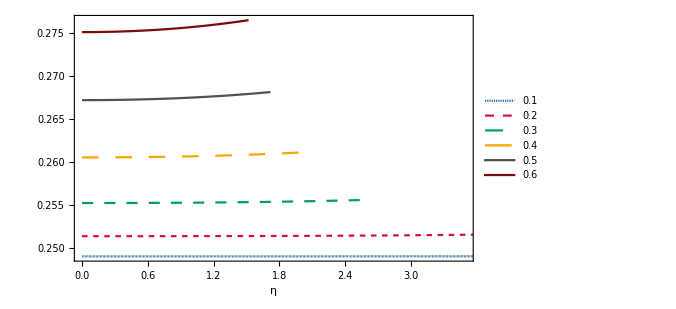

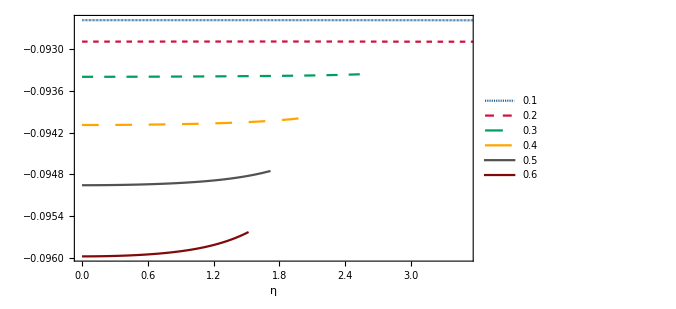

```mathematica
ListLinePlot[{Re[Ta1[[1]]],Re[Ta1[[2]]],Re[Ta1[[3]]],Re[Ta1[[4]]],Re[Ta1[[5]]],Re[Ta1[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[Ta1[[1]]],Im[Ta1[[2]]],Im[Ta1[[3]]],Im[Ta1[[4]]],Im[Ta1[[5]]],Im[Ta1[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.31}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
(Max[Re[Tda1[[1]]]]-Min[Re[Tda1[[1]]]])/Min[Re[Tda1[[1]]]]*100
(Max[Im[Tda1[[1]]]]-Min[Im[Tda1[[1]]]])/Min[Im[Tda1[[1]]]]*100
(Max[Re[Tda1[[6]]]]-Min[Re[Tda1[[6]]]])/Min[Re[Tda1[[6]]]]*100
(Max[Im[Tda1[[6]]]]-Min[Im[Tda1[[6]]]])/Min[Im[Tda1[[6]]]]*100
```

0.0437993

-0.021226

0.504529

-0.363414

#### Polar modes

```mathematica
Tp1={{{0,0.24904953330653543-0.09259088336848395 ⅈ},{1/25+ⅈ/25,0.24904802144741017-0.09259068521134566 ⅈ},{2/25+(2 ⅈ)/25,0.24904348641236068-0.0925900908067607 ⅈ},{3/25+(3 ⅈ)/25,0.24903592984233075-0.09258910035707213 ⅈ},{4/25+(4 ⅈ)/25,0.2490253544658671-0.0925877141987599 ⅈ},{1/5+ⅈ/5,0.24901176409489034-0.09258593280199985 ⅈ},{6/25+(6 ⅈ)/25,0.24899516361669569-0.09258375676977225 ⅈ},{7/25+(7 ⅈ)/25,0.24897555898373266-0.09258118683672371 ⅈ},{8/25+(8 ⅈ)/25,0.24895295720121166-0.09257822386778715 ⅈ},{9/25+(9 ⅈ)/25,0.24892736631259765-0.09257486885657035 ⅈ},{2/5+(2 ⅈ)/5,0.24889879538303944-0.09257112292349953 ⅈ},{11/25+(11 ⅈ)/25,0.24886725448085373-0.09256698731377806 ⅈ},{12/25+(12 ⅈ)/25,0.24883275465709284-0.09256246339510338 ⅈ},{13/25+(13 ⅈ)/25,0.24879530792332546-0.09255755265520128 ⅈ},{14/25+(14 ⅈ)/25,0.24875492722771436-0.09255225669916946 ⅈ},{3/5+(3 ⅈ)/5,0.24871162642949649-0.09254657724664561 ⅈ},{16/25+(16 ⅈ)/25,0.2486654202719753-0.0925405161288129 ⅈ},{17/25+(17 ⅈ)/25,0.24861632435413805-0.09253407528525519 ⅈ},{18/25+(18 ⅈ)/25,0.24856435510101618-0.09252725676067636 ⅈ},{19/25+(19 ⅈ)/25,0.24850952973290744-0.09252006270149633 ⅈ},{4/5+(4 ⅈ)/5,0.24845186623358242-0.09251249535233903 ⅈ},{21/25+(21 ⅈ)/25,0.24839138331759844-0.0925045570524253 ⅈ},{22/25+(22 ⅈ)/25,0.24832810039684347-0.0924962502318858 ⅈ},{23/25+(23 ⅈ)/25,0.24826203754643378-0.09248757740800723 ⅈ},{24/25+(24 ⅈ)/25,0.24819321547008644-0.09247854118142634 ⅈ},{1+ⅈ,0.24812165546508716-0.09246914423228553 ⅈ},{26/25+(26 ⅈ)/25,0.24804737938697038-0.09245938931636269 ⅈ},{27/25+(27 ⅈ)/25,0.24797040961402697-0.0924492792611898 ⅈ},{28/25+(28 ⅈ)/25,0.24789076901174878-0.09243881696217099 ⅈ},{29/25+(29 ⅈ)/25,0.2478084808973191-0.0924280053787147 ⅈ},{6/5+(6 ⅈ)/5,0.24772356900424886-0.09241684753038923 ⅈ},{31/25+(31 ⅈ)/25,0.24763605744725758-0.09240534649311437 ⅈ},{32/25+(32 ⅈ)/25,0.24754597068749065-0.09239350539539905 ⅈ},{33/25+(33 ⅈ)/25,0.24745333349815957-0.09238132741463492 ⅈ},{34/25+(34 ⅈ)/25,0.2473581709306859-0.09236881577345511 ⅈ},{7/5+(7 ⅈ)/5,0.24726050828142507-0.09235597373616664 ⅈ},{36/25+(36 ⅈ)/25,0.24716037105903796-0.09234280460526449 ⅈ},{37/25+(37 ⅈ)/25,0.2470577849525745-0.09232931171803441 ⅈ},{38/25+(38 ⅈ)/25,0.24695277580032607-0.09231549844325086 ⅈ},{39/25+(39 ⅈ)/25,0.24684536955949832-0.09230136817797614 ⅈ},{8/5+(8 ⅈ)/5,0.24673559227674952-0.09228692434446559 ⅈ},{41/25+(41 ⅈ)/25,0.2466234700596347-0.09227217038718331 ⅈ},{42/25+(42 ⅈ)/25,0.24650902904898875-0.09225710976993239 ⅈ},{43/25+(43 ⅈ)/25,0.24639229539227794-0.09224174597310285 ⅈ},{44/25+(44 ⅈ)/25,0.24627329521794314-0.09222608249103968 ⅈ},{9/5+(9 ⅈ)/5,0.24615205461075262-0.09221012282953296 ⅈ},{46/25+(46 ⅈ)/25,0.246028599588178-0.09219387050343222 ⅈ},{47/25+(47 ⅈ)/25,0.2459029560778038-0.0921773290343846 ⅈ},{48/25+(48 ⅈ)/25,0.24577514989577232-0.09216050194869913 ⅈ},{49/25+(49 ⅈ)/25,0.24564520672626838-0.0921433927753351 ⅈ},{2+2 ⅈ,0.24551315210203767-0.09212600504401602 ⅈ},{51/25+(51 ⅈ)/25,0.2453790113859339-0.09210834228346694 ⅈ},{52/25+(52 ⅈ)/25,0.24524280975348467-0.09209040801977465 ⅈ},{53/25+(53 ⅈ)/25,0.24510457217646364-0.09207220577486919 ⅈ},{54/25+(54 ⅈ)/25,0.24496432340745325-0.09205373906512453 ⅈ},{11/5+(11 ⅈ)/5,0.24482208796538119-0.09203501140007705 ⅈ},{56/25+(56 ⅈ)/25,0.24467789012200988-0.09201602628125859 ⅈ},{57/25+(57 ⅈ)/25,0.24453175388935822-0.09199678720114235 ⅈ},{58/25+(58 ⅈ)/25,0.24438370300803197-0.09197729764219861 ⅈ},{59/25+(59 ⅈ)/25,0.24423376093643764-0.09195756107605728 ⅈ},{12/5+(12 ⅈ)/5,0.24408195084085496-0.09193758096277463 ⅈ},{61/25+(61 ⅈ)/25,0.24392829558634002-0.09191736075020102 ⅈ},{62/25+(62 ⅈ)/25,0.24377281772843215-0.09189690387344614 ⅈ},{63/25+(63 ⅈ)/25,0.24361553950563586-0.09187621375443891 ⅈ},{64/25+(64 ⅈ)/25,0.24345648283264867-0.0918552938015788 ⅈ},{13/5+(13 ⅈ)/5,0.24329566929430713-0.09183414740947454 ⅈ},{66/25+(66 ⅈ)/25,0.2431331201402198-0.09181277795876805 ⅈ},{67/25+(67 ⅈ)/25,0.24296885628005976-0.09179118881603937 ⅈ},{68/25+(68 ⅈ)/25,0.24280289827948645-0.0917693833337893 ⅈ},{69/25+(69 ⅈ)/25,0.24263526635666782-0.09174736485049735 ⅈ},{14/5+(14 ⅈ)/5,0.24246598037937486-0.09172513669075057 ⅈ},{71/25+(71 ⅈ)/25,0.2422950598626197-0.0917027021654412 ⅈ},{72/25+(72 ⅈ)/25,0.24212252396680953-0.09168006457202899 ⅈ},{73/25+(73 ⅈ)/25,0.24194839149638875-0.09165722719486605 ⅈ},{74/25+(74 ⅈ)/25,0.24177268089894394-0.0916341933055806 ⅈ},{3+3 ⅈ,0.24159541026474338-0.09161096616351724 ⅈ},{76/25+(76 ⅈ)/25,0.24141659732668844-0.09158754901623024 ⅈ},{77/25+(77 ⅈ)/25,0.24123625946064967-0.09156394510002792 ⅈ},{78/25+(78 ⅈ)/25,0.2410544136861658-0.09154015764056496 ⅈ},{79/25+(79 ⅈ)/25,0.24087107666748095-0.09151618985348026 ⅈ},{16/5+(16 ⅈ)/5,0.24068626471489893-0.09149204494507777 ⅈ},{81/25+(81 ⅈ)/25,0.24049999378643253-0.09146772611304844 ⅈ},{82/25+(82 ⅈ)/25,0.24031227948972678-0.09144323654723019 ⅈ},{83/25+(83 ⅈ)/25,0.2401231370842376-0.09141857943040466 ⅈ},{84/25+(84 ⅈ)/25,0.23993258148364538-0.09139375793912796 ⅈ},{17/5+(17 ⅈ)/5,0.2397406272584857-0.09136877524459404 ⅈ},{86/25+(86 ⅈ)/25,0.23954728863898042-0.09134363451352835 ⅈ},{87/25+(87 ⅈ)/25,0.23935257951805186-0.09131833890911041 ⅈ},{88/25+(88 ⅈ)/25,0.23915651345450367-0.09129289159192333 ⅈ},{89/25+(89 ⅈ)/25,0.23895910367635495-0.09126729572092905 ⅈ},{18/5+(18 ⅈ)/5,0.2387603630843117-0.09124155445446727 ⅈ},{91/25+(91 ⅈ)/25,0.23856030425536287-0.09121567095127753 ⅈ},{92/25+(92 ⅈ)/25,0.23835893944648767-0.09118964837154189 ⅈ},{93/25+(93 ⅈ)/25,0.23815628059846236-0.0911634898779487 ⅈ},{94/25+(94 ⅈ)/25,0.2379523393397549-0.09113719863677444 ⅈ},{19/5+(19 ⅈ)/5,0.23774712699049622-0.09111077781898393 ⅈ},{96/25+(96 ⅈ)/25,0.2375406545665186-0.09108423060134747 ⅈ},{97/25+(97 ⅈ)/25,0.23733293278345086-0.09105756016757378 ⅈ},{98/25+(98 ⅈ)/25,0.23712397206086175-0.0910307697094585 ⅈ},{99/25+(99 ⅈ)/25,0.23691378252644327-0.09100386242804663 ⅈ},{4+4 ⅈ,0.23670237402022515-0.09097684153480899 ⅈ},{101/25+(101 ⅈ)/25,0.23648975609881412-0.09094971025283181 ⅈ},{102/25+(102 ⅈ)/25,0.23627593803965058-0.09092247181801831 ⅈ},{103/25+(103 ⅈ)/25,0.23606092884527624-0.0908951294803031 ⅈ},{104/25+(104 ⅈ)/25,0.23584473724760677-0.09086768650487716 ⅈ},{21/5+(21 ⅈ)/5,0.23562737171220424-0.09084014617342458 ⅈ},{106/25+(106 ⅈ)/25,0.23540884044254395-0.09081251178536967 ⅈ},{107/25+(107 ⅈ)/25,0.23518915138427093-0.09078478665913471 ⅈ},{108/25+(108 ⅈ)/25,0.23496831222944203-0.09075697413340769 ⅈ},{109/25+(109 ⅈ)/25,0.23474633042074938-0.09072907756841997 ⅈ},{22/5+(22 ⅈ)/5,0.2345232131557218-0.09070110034723408 ⅈ},{111/25+(111 ⅈ)/25,0.23429896739090045-0.09067304587704039 ⅈ},{112/25+(112 ⅈ)/25,0.23407359984598644-0.09064491759046428 ⅈ},{113/25+(113 ⅈ)/25,0.23384711700795696-0.09061671894688192 ⅈ},{114/25+(114 ⅈ)/25,0.2336195251351476-0.09058845343374594 ⅈ},{23/5+(23 ⅈ)/5,0.23339083026129945-0.09056012456792051 ⅈ},{116/25+(116 ⅈ)/25,0.23316103819956782-0.09053173589702583 ⅈ},{117/25+(117 ⅈ)/25,0.23293015454649182-0.09050329100079207 ⅈ},{118/25+(118 ⅈ)/25,0.23269818468592304-0.09047479349242353 ⅈ},{119/25+(119 ⅈ)/25,0.23246513379291175-0.0904462470199717 ⅈ},{24/5+(24 ⅈ)/5,0.2322310068375501-0.090417655267719 ⅈ},{121/25+(121 ⅈ)/25,0.2319958085887708-0.09038902195757238 ⅈ},{122/25+(122 ⅈ)/25,0.2317595436181011-0.09036035085046719 ⅈ},{123/25+(123 ⅈ)/25,0.23152221630337108-0.0903316457477816 ⅈ},{124/25+(124 ⅈ)/25,0.23128383083237597-0.09030291049276207 ⅈ},{5+5 ⅈ,0.23104439120649245-0.09027414897195941 ⅈ},{126/25+(126 ⅈ)/25,0.23080390124424843-0.0902453651166765 ⅈ},{127/25+(127 ⅈ)/25,0.2305623645848465-0.09021656290442762 ⅈ},{128/25+(128 ⅈ)/25,0.23031978469164088-0.09018774636040969 ⅈ},{129/25+(129 ⅈ)/25,0.2300761648555688-0.09015891955898565 ⅈ},{26/5+(26 ⅈ)/5,0.22983150819853565-0.09013008662518074 ⅈ},{131/25+(131 ⅈ)/25,0.2295858176767551-0.09010125173619164 ⅈ},{132/25+(132 ⅈ)/25,0.229339096084044-0.09007241912290899 ⅈ},{133/25+(133 ⅈ)/25,0.22909134605507395-0.09004359307145351 ⅈ},{134/25+(134 ⅈ)/25,0.22884257006857794-0.09001477792472679 ⅈ},{27/5+(27 ⅈ)/5,0.22859277045051565-0.08998597808397611 ⅈ},{136/25+(136 ⅈ)/25,0.2283419493771957-0.08995719801037459 ⅈ},{137/25+(137 ⅈ)/25,0.22809010887835734-0.08992844222661668 ⅈ},{138/25+(138 ⅈ)/25,0.22783725084021214-0.08989971531852961 ⅈ},{139/25+(139 ⅈ)/25,0.2275833770084459-0.08987102193670114 ⅈ},{28/5+(28 ⅈ)/5,0.22732848899118352-0.08984236679812407 ⅈ},{141/25+(141 ⅈ)/25,0.22707258826191629-0.08981375468785832 ⅈ},{142/25+(142 ⅈ)/25,0.2268156761623936-0.0897851904607103 ⅈ},{143/25+(143 ⅈ)/25,0.22655775390548044-0.08975667904293104 ⅈ},{144/25+(144 ⅈ)/25,0.22629882257798137-0.08972822543393265 ⅈ},{29/5+(29 ⅈ)/5,0.22603888314343315-0.08969983470802448 ⅈ},{146/25+(146 ⅈ)/25,0.22577793644486607-0.08967151201616852 ⅈ},{147/25+(147 ⅈ)/25,0.22551598320753724-0.0896432625877556 ⅈ},{148/25+(148 ⅈ)/25,0.22525302404163533-0.08961509173240186 ⅈ},{149/25+(149 ⅈ)/25,0.22498905944495964-0.08958700484176707 ⅈ},{6+6 ⅈ,0.2247240898055747-0.08955900739139427 ⅈ},{151/25+(151 ⅈ)/25,0.22445811540444144-0.08953110494257227 ⅈ},{152/25+(152 ⅈ)/25,0.22419113641802724-0.08950330314422046 ⅈ},{153/25+(153 ⅈ)/25,0.22392315292089607-0.08947560773479776 ⅈ},{154/25+(154 ⅈ)/25,0.2236541648882804-0.08944802454423487 ⅈ},{31/5+(31 ⅈ)/5,0.22338417219863732-0.08942055949589138 ⅈ},{156/25+(156 ⅈ)/25,0.22311317463618907-0.08939321860853787 ⅈ},{157/25+(157 ⅈ)/25,0.22284117189345162-0.0893660079983635 ⅈ},{158/25+(158 ⅈ)/25,0.22256816357375145-0.08933893388100979 ⅈ},{159/25+(159 ⅈ)/25,0.22229414919373394-0.08931200257363094 ⅈ},{32/5+(32 ⅈ)/5,0.22201912818586372-0.08928522049698126 ⅈ},{161/25+(161 ⅈ)/25,0.22174309990092023-0.08925859417753067 ⅈ},{162/25+(162 ⅈ)/25,0.2214660636104897-0.08923213024960785 ⅈ},{163/25+(163 ⅈ)/25,0.2211880185094558-0.08920583545757263 ⅈ},{164/25+(164 ⅈ)/25,0.22090896371849092-0.08917971665801719 ⅈ},{33/5+(33 ⅈ)/5,0.2206288982865506-0.08915378082199746 ⅈ},{166/25+(166 ⅈ)/25,0.22034782119337215-0.08912803503729423 ⅈ},{167/25+(167 ⅈ)/25,0.2200657313519814-0.08910248651070567 ⅈ},{168/25+(168 ⅈ)/25,0.21978262761120795-0.0890771425703703 ⅈ},{169/25+(169 ⅈ)/25,0.2194985087582125-0.08905201066812232 ⅈ},{34/5+(34 ⅈ)/5,0.21921337352102793-0.08902709838187843 ⅈ},{171/25+(171 ⅈ)/25,0.21892722057111694-0.08900241341805791 ⅈ},{172/25+(172 ⅈ)/25,0.21864004852594823-0.08897796361403508 ⅈ},{173/25+(173 ⅈ)/25,0.21835185595159387-0.0889537569406254 ⅈ},{174/25+(174 ⅈ)/25,0.21806264136535083-0.08892980150460553 ⅈ},{7+7 ⅈ,0.21777240323838853-0.08890610555126699 ⅈ},{176/25+(176 ⅈ)/25,0.2174811399984254-0.08888267746700489 ⅈ},{177/25+(177 ⅈ)/25,0.2171888500324376-0.08885952578194112 ⅈ},{178/25+(178 ⅈ)/25,0.2168955316894018-0.08883665917258268 ⅈ}},{{0,0.2513922213744943-0.09289841463615552 ⅈ},{1/25+ⅈ/25,0.2513861772520305-0.09289762475851178 ⅈ},{2/25+(2 ⅈ)/25,0.2513680538446794-0.09289525620959002 ⅈ},{3/25+(3 ⅈ)/25,0.25133787801589286-0.09289131224081079 ⅈ},{4/25+(4 ⅈ)/25,0.2512956942724765-0.0928857982417839 ⅈ},{1/5+ⅈ/5,0.25124156439244777-0.09287872169949693 ⅈ},{6/25+(6 ⅈ)/25,0.2511755669056639-0.09287009214122863 ⅈ},{7/25+(7 ⅈ)/25,0.2510977964429324-0.09285992106306223 ⅈ},{8/25+(8 ⅈ)/25,0.2510083629654824-0.09284822184534625 ⅈ},{9/25+(9 ⅈ)/25,0.25090739088849184-0.09283500965665373 ⅈ},{2/5+(2 ⅈ)/5,0.2507950181137667-0.09282030134794862 ⅈ},{11/25+(11 ⅈ)/25,0.25067139498761654-0.09280411533877538 ⅈ},{12/25+(12 ⅈ)/25,0.2505366832004691-0.09278647149734214 ⅈ},{13/25+(13 ⅈ)/25,0.2503910546448329-0.09276739101637446 ⅈ},{14/25+(14 ⅈ)/25,0.25023469024787026-0.09274689628657631 ⅈ},{3/5+(3 ⅈ)/5,0.2500677787941469-0.0927250107694542 ⅈ},{16/25+(16 ⅈ)/25,0.24989051575311233-0.0927017588711447 ⅈ},{17/25+(17 ⅈ)/25,0.24970310212461488-0.09267716581874226 ⅈ},{18/25+(18 ⅈ)/25,0.24950574331431652-0.09265125754046168 ⅈ},{19/25+(19 ⅈ)/25,0.24929864804931812-0.09262406055079025 ⅈ},{4/5+(4 ⅈ)/5,0.24908202734268603-0.09259560184160287 ⅈ},{21/25+(21 ⅈ)/25,0.24885609351394264-0.09256590878002775 ⅈ},{22/25+(22 ⅈ)/25,0.24862105927099626-0.09253500901367005 ⅈ},{23/25+(23 ⅈ)/25,0.24837713685746957-0.09250293038363042 ⅈ},{24/25+(24 ⅈ)/25,0.24812453726797978-0.09246970084559618 ⅈ},{1+ⅈ,0.24786346953264352-0.09243534839913839 ⅈ},{26/25+(26 ⅈ)/25,0.24759414007094235-0.09239990102522094 ⅈ},{27/25+(27 ⅈ)/25,0.24731675211409712-0.09236338663181717 ⅈ},{28/25+(28 ⅈ)/25,0.24703150519426323-0.09232583300743495 ⅈ},{29/25+(29 ⅈ)/25,0.24673859469817036-0.09228726778227686 ⅈ},{6/5+(6 ⅈ)/5,0.24643821148228384-0.09224771839669982 ⅈ},{31/25+(31 ⅈ)/25,0.24613054154614605-0.0922072120765939 ⅈ},{32/25+(32 ⅈ)/25,0.24581576576026043-0.0921657758152677 ⅈ},{33/25+(33 ⅈ)/25,0.2454940596446867-0.09212343636140789 ⅈ},{34/25+(34 ⅈ)/25,0.2451655931944166-0.09208022021266997 ⅈ},{7/5+(7 ⅈ)/5,0.24483053074757696-0.09203615361445827 ⅈ},{36/25+(36 ⅈ)/25,0.24448903089255125-0.09199126256345731 ⅈ},{37/25+(37 ⅈ)/25,0.24414124641020787-0.09194557281549115 ⅈ},{38/25+(38 ⅈ)/25,0.24378732424756172-0.0918991098973041 ⅈ},{39/25+(39 ⅈ)/25,0.2434274055193686-0.09185189912187641 ⅈ},{8/5+(8 ⅈ)/5,0.24306162553434524-0.09180396560691251 ⅈ},{41/25+(41 ⅈ)/25,0.24269011384291808-0.09175533429616427 ⅈ},{42/25+(42 ⅈ)/25,0.24231299430362352-0.09170602998327815 ⅈ},{43/25+(43 ⅈ)/25,0.24193038516550483-0.09165607733788081 ⅈ},{44/25+(44 ⅈ)/25,0.2415423991640731-0.09160550093364422 ⅈ},{9/5+(9 ⅈ)/5,0.24114914362861659-0.09155432527809805 ⅈ},{46/25+(46 ⅈ)/25,0.24075072059885452-0.09150257484398011 ⅈ},{47/25+(47 ⅈ)/25,0.24034722694913102-0.09145027410194126 ⅈ},{48/25+(48 ⅈ)/25,0.2399387545185379-0.09139744755444211 ⅈ},{49/25+(49 ⅈ)/25,0.2395253902455321-0.0913441197707019 ⅈ},{2+2 ⅈ,0.23910721630578122-0.09129031542257776 ⅈ},{51/25+(51 ⅈ)/25,0.23868431025212714-0.09123605932127257 ⅈ},{52/25+(52 ⅈ)/25,0.23825674515569698-0.09118137645478575 ⅈ},{53/25+(53 ⅈ)/25,0.23782458974732337-0.09112629202603748 ⅈ},{54/25+(54 ⅈ)/25,0.23738790855855507-0.09107083149161055 ⅈ},{11/5+(11 ⅈ)/5,0.2369467620616442-0.09101502060106809 ⅈ},{56/25+(56 ⅈ)/25,0.23650120680799658-0.09095888543681559 ⅈ},{57/25+(57 ⅈ)/25,0.23605129556465754-0.09090245245448862 ⅈ},{58/25+(58 ⅈ)/25,0.23559707744848396-0.09084574852385581 ⅈ},{59/25+(59 ⅈ)/25,0.23513859805772375-0.09078880097023496 ⅈ},{12/5+(12 ⅈ)/5,0.23467589960078636-0.09073163761643022 ⅈ},{61/25+(61 ⅈ)/25,0.23420902102204244-0.0906742868252037 ⅈ},{62/25+(62 ⅈ)/25,0.23373799812454057-0.09061677754230046 ⅈ},{63/25+(63 ⅈ)/25,0.23326286368957094-0.0905591393400547 ⅈ},{64/25+(64 ⅈ)/25,0.2327836475930458-0.09050140246160604 ⅈ},{13/5+(13 ⅈ)/5,0.23230037691869693-0.09044359786576295 ⅈ},{66/25+(66 ⅈ)/25,0.2318130760681228-0.0903857572725519 ⅈ},{67/25+(67 ⅈ)/25,0.23132176686774167-0.09032791320949603 ⅈ},{68/25+(68 ⅈ)/25,0.2308264686727298-0.09027009905866965 ⅈ},{69/25+(69 ⅈ)/25,0.23032719846804448-0.09021234910457789 ⅈ},{14/5+(14 ⅈ)/5,0.22982397096664756-0.09015469858291378 ⅈ},{71/25+(71 ⅈ)/25,0.22931679870506183-0.09009718373024671 ⅈ},{72/25+(72 ⅈ)/25,0.22880569213640514-0.09003984183469861 ⅈ},{73/25+(73 ⅈ)/25,0.22829065972105958-0.08998271128766616 ⅈ},{74/25+(74 ⅈ)/25,0.22777170801514365-0.08992583163664804 ⅈ},{3+3 ⅈ,0.22724884175696589-0.08986924363923826 ⅈ},{76/25+(76 ⅈ)/25,0.22672206395164662-0.0898129893183474 ⅈ},{77/25+(77 ⅈ)/25,0.2261913759541038-0.08975711201871393 ⅈ},{78/25+(78 ⅈ)/25,0.2256567775506061-0.089701656464769 ⅈ},{79/25+(79 ⅈ)/25,0.22511826703910615-0.08964666881991781 ⅈ},{16/5+(16 ⅈ)/5,0.22457584130857217-0.08959219674730075 ⅈ},{81/25+(81 ⅈ)/25,0.22402949591754645-0.08953828947209683 ⅈ},{82/25+(82 ⅈ)/25,0.22347922517216562-0.08948499784543283 ⅈ},{83/25+(83 ⅈ)/25,0.22292502220388702-0.08943237440995755 ⅈ},{84/25+(84 ⅈ)/25,0.22236687904717353-0.08938047346714183 ⅈ},{17/5+(17 ⅈ)/5,0.2218047867173993-0.08932935114636205 ⅈ},{86/25+(86 ⅈ)/25,0.22123873528924812-0.08927906547582128 ⅈ},{87/25+(87 ⅈ)/25,0.22066871397588647-0.08922967645536116 ⅈ},{88/25+(88 ⅈ)/25,0.2200947112092064-0.08918124613121173 ⅈ},{89/25+(89 ⅈ)/25,0.21951671472144296-0.08913383867272358 ⅈ},{18/5+(18 ⅈ)/5,0.21893471162848674-0.08908752045111935 ⅈ},{91/25+(91 ⅈ)/25,0.2183486885152241-0.08904236012029738 ⅈ}},{{0,0.2552443161152394-0.09340456216904312 ⅈ},{1/25+ⅈ/25,0.25523071954783044-0.09340279449208581 ⅈ},{2/25+(2 ⅈ)/25,0.2551899772951585-0.09339749703267484 ⅈ},{3/25+(3 ⅈ)/25,0.25512223089622954-0.09338868642088136 ⅈ},{4/25+(4 ⅈ)/25,0.25502771311651923-0.09337639003518598 ⅈ},{1/5+ⅈ/5,0.2549067434400436-0.0933606455171281 ⅈ},{6/25+(6 ⅈ)/25,0.25475972201522784-0.09334150011988661 ⅈ},{7/25+(7 ⅈ)/25,0.2545871223187073-0.09331900992027731 ⅈ},{8/25+(8 ⅈ)/25,0.2543894828261668-0.0932932389261344 ⅈ},{9/25+(9 ⅈ)/25,0.25416739799846794-0.09326425811313746 ⅈ},{2/5+(2 ⅈ)/5,0.2539215088915216-0.09323214442514009 ⅈ},{11/25+(11 ⅈ)/25,0.25365249368180365-0.09319697977019102 ⅈ},{12/25+(12 ⅈ)/25,0.25336105836940803-0.09315885004109008 ⅈ},{13/25+(13 ⅈ)/25,0.2530479278810876-0.09311784418493017 ⅈ},{14/25+(14 ⅈ)/25,0.2527138377509415-0.09307405334110118 ⅈ},{3/5+(3 ⅈ)/5,0.2523595265100649-0.09302757006209497 ⅈ},{16/25+(16 ⅈ)/25,0.2519857288717583-0.09297848762650143 ⅈ},{17/25+(17 ⅈ)/25,0.25159316975816765-0.0929268994490884 ⅈ},{18/25+(18 ⅈ)/25,0.2511825591790835-0.09287289858898748 ⅈ},{19/25+(19 ⅈ)/25,0.2507545879448479-0.09281657735384942 ⅈ},{4/5+(4 ⅈ)/5,0.25030992417308984-0.09275802699540271 ⅈ},{21/25+(21 ⅈ)/25,0.24984921053301426-0.09269733749011577 ⅈ},{22/25+(22 ⅈ)/25,0.24937306216056826-0.09263459739754781 ⅈ},{23/25+(23 ⅈ)/25,0.248882065172182-0.09256989378839077 ⅈ},{24/25+(24 ⅈ)/25,0.2483767757030328-0.09250331223404881 ⅈ},{1+ⅈ,0.2478577193970316-0.09243493684977723 ⅈ},{26/25+(26 ⅈ)/25,0.2473253912791739-0.09236485038381953 ⅈ},{27/25+(27 ⅈ)/25,0.2467802559458264-0.09229313434555995 ⅈ},{28/25+(28 ⅈ)/25,0.246222748014357-0.09221986916638718 ⅈ},{29/25+(29 ⅈ)/25,0.24565327277978624-0.09214513438768597 ⅈ},{6/5+(6 ⅈ)/5,0.24507220703249588-0.09206900887110649 ⅈ},{31/25+(31 ⅈ)/25,0.2444798999972142-0.09199157102696942 ⅈ},{32/25+(32 ⅈ)/25,0.24387667435933014-0.09191289905733485 ⅈ},{33/25+(33 ⅈ)/25,0.24326282734996452-0.09183307121087958 ⅈ},{34/25+(34 ⅈ)/25,0.24263863186608361-0.09175216604728775 ⅈ},{7/5+(7 ⅈ)/5,0.24200433760625956-0.09167026270935646 ⅈ},{36/25+(36 ⅈ)/25,0.24136017220646871-0.09158744120145841 ⅈ},{37/25+(37 ⅈ)/25,0.2407063423636029-0.09150378267338558 ⅈ},{38/25+(38 ⅈ)/25,0.2400430349371775-0.09141936970892785 ⅈ},{39/25+(39 ⅈ)/25,0.23937041802211056-0.09133428661882445 ⅈ},{8/5+(8 ⅈ)/5,0.23868864198745357-0.09124861973796569 ⅈ},{41/25+(41 ⅈ)/25,0.2379978404776276-0.09116245772692672 ⅈ},{42/25+(42 ⅈ)/25,0.23729813137410813-0.09107589187808687 ⅈ},{43/25+(43 ⅈ)/25,0.23658961771663609-0.09098901642673067 ⅈ},{44/25+(44 ⅈ)/25,0.23587238858396428-0.09090192886764871 ⅈ},{9/5+(9 ⅈ)/5,0.2351465199349005-0.09081473027785401 ⅈ},{46/25+(46 ⅈ)/25,0.2344120754110167-0.09072752564611437 ⅈ},{47/25+(47 ⅈ)/25,0.2336691071028814-0.09064042421006871 ⅈ},{48/25+(48 ⅈ)/25,0.23291765628206643-0.09055353980175063 ⅈ},{49/25+(49 ⅈ)/25,0.2321577541014946-0.09046699120238891 ⅈ},{2+2 ⅈ,0.23138942226695333-0.09038090250738859 ⅈ},{51/25+(51 ⅈ)/25,0.230612673682812-0.09029540350242346 ⅈ},{52/25+(52 ⅈ)/25,0.22982751307516341-0.09021063005158965 ⅈ},{53/25+(53 ⅈ)/25,0.22903393759577068-0.09012672449857863 ⅈ},{54/25+(54 ⅈ)/25,0.22823193741035083-0.09004383608182945 ⅈ},{11/5+(11 ⅈ)/5,0.22742149627487324-0.08996212136461179 ⅈ},{56/25+(56 ⅈ)/25,0.22660259210369973-0.08988174468097113 ⅈ},{57/25+(57 ⅈ)/25,0.22577519753355568-0.08980287859843546 ⅈ},{58/25+(58 ⅈ)/25,0.22493928048749415-0.08972570439833646 ⅈ},{59/25+(59 ⅈ)/25,0.22409480474321117-0.08965041257453299 ⅈ},{12/5+(12 ⅈ)/5,0.2232417305102888-0.08957720335123921 ⅈ},{61/25+(61 ⅈ)/25,0.22238001502119137-0.08950628722054928 ⅈ},{62/25+(62 ⅈ)/25,0.22150961314111547-0.08943788550010931 ⅈ},{63/25+(63 ⅈ)/25,0.22063047800211308-0.08937223091120992 ⅈ},{64/25+(64 ⅈ)/25,0.2197425616672511-0.08930956817735317 ⅈ}},{{0,0.2605316834521421-0.09410018395896062 ⅈ},{1/25+ⅈ/25,0.260507482443302-0.09409706237703763 ⅈ},{2/25+(2 ⅈ)/25,0.26043503927076683-0.09408771567951954 ⅈ},{3/25+(3 ⅈ)/25,0.26031482782666604-0.09407219742125486 ⅈ},{4/25+(4 ⅈ)/25,0.2601476186702098-0.09405059483673647 ⅈ},{1/5+ⅈ/5,0.259934451851668-0.094023025990767 ⅈ},{6/25+(6 ⅈ)/25,0.2596766018559289-0.09398963610963403 ⅈ},{7/25+(7 ⅈ)/25,0.25937553721180917-0.09395059336648563 ⅈ},{8/25+(8 ⅈ)/25,0.25903287741116193-0.0939060844043474 ⅈ},{9/25+(9 ⅈ)/25,0.2586503496248578-0.09385630986309514 ⅈ},{2/5+(2 ⅈ)/5,0.2582297473332843-0.09380148013676275 ⅈ},{11/25+(11 ⅈ)/25,0.25777289249301005-0.09374181153409519 ⅈ},{12/25+(12 ⅈ)/25,0.2572816023238151-0.09367752295742753 ⅈ},{13/25+(13 ⅈ)/25,0.2567576612910781-0.09360883316027836 ⅈ},{14/25+(14 ⅈ)/25,0.2562027984245006-0.09353595859754225 ⅈ},{3/5+(3 ⅈ)/5,0.25561866977900044-0.09345911184636842 ⅈ},{16/25+(16 ⅈ)/25,0.2550068456115255-0.09337850055115726 ⅈ},{17/25+(17 ⅈ)/25,0.2543688017092988-0.09329432683157551 ⅈ},{18/25+(18 ⅈ)/25,0.25370591424388644-0.09320678708626143 ⅈ},{19/25+(19 ⅈ)/25,0.25301945752223903-0.09311607212488422 ⅈ},{4/5+(4 ⅈ)/5,0.25231060404207795-0.09302236756543829 ⅈ},{21/25+(21 ⅈ)/25,0.2515804263189709-0.09292585444040095 ⅈ},{22/25+(22 ⅈ)/25,0.25082990002393846-0.0928267099633445 ⅈ},{23/25+(23 ⅈ)/25,0.2500599080446546-0.09272510841581953 ⅈ},{24/25+(24 ⅈ)/25,0.249271245154452-0.09262122212220192 ⅈ},{1+ⅈ,0.24846462303800165-0.09251522248735088 ⅈ},{26/25+(26 ⅈ)/25,0.2476406754790426-0.09240728107818905 ⅈ},{27/25+(27 ⅈ)/25,0.2467999635634388-0.09229757073563757 ⅈ},{28/25+(28 ⅈ)/25,0.245942980790445-0.09218626670776707 ⅈ},{29/25+(29 ⅈ)/25,0.24507015801712126-0.09207354779862195 ⅈ},{6/5+(6 ⅈ)/5,0.24418186818630003-0.09195959753007399 ⅈ},{31/25+(31 ⅈ)/25,0.24327843080838532-0.09184460531633983 ⅈ},{32/25+(32 ⅈ)/25,0.24236011618252737-0.0917287676525857 ⅈ},{33/25+(33 ⅈ)/25,0.2414271493542445-0.09161228932042066 ⅈ},{34/25+(34 ⅈ)/25,0.24047971381513047-0.0914953846141333 ⅈ},{7/5+(7 ⅈ)/5,0.23951795495654665-0.09137827859232434 ⅈ},{36/25+(36 ⅈ)/25,0.23854198329369813-0.0912612083601793 ⅈ},{37/25+(37 ⅈ)/25,0.23755187747967973-0.09114442438805914 ⅈ},{38/25+(38 ⅈ)/25,0.23654768713131322-0.09102819187238674 ⅈ},{39/25+(39 ⅈ)/25,0.2355294354901714-0.09091279214500218 ⅈ},{8/5+(8 ⅈ)/5,0.23449712194332736-0.09079852413725358 ⅈ},{41/25+(41 ⅈ)/25,0.23345072442926787-0.0906857059050936 ⅈ},{42/25+(42 ⅈ)/25,0.23239020175520766-0.09057467622135465 ⅈ},{43/25+(43 ⅈ)/25,0.23131549585286035-0.09046579624116866 ⅈ},{44/25+(44 ⅈ)/25,0.23022653400065157-0.0903594512461556 ⅈ},{9/5+(9 ⅈ)/5,0.22912323104148338-0.09025605247250046 ⅈ},{46/25+(46 ⅈ)/25,0.22800549162653164-0.09015603902732723 ⅈ},{47/25+(47 ⅈ)/25,0.22687321251724687-0.09005987989680654 ⅈ},{48/25+(48 ⅈ)/25,0.22572628497975952-0.08996807604813549 ⅈ},{49/25+(49 ⅈ)/25,0.2245645973083223-0.08988116262581287 ⅈ},{2+2 ⅈ,0.22338803751725528-0.08979971124040159 ⅈ}},{{0,0.2671585575236661-0.09497327544666492 ⅈ},{1/25+ⅈ/25,0.267120587666371-0.094968432608322 ⅈ},{2/25+(2 ⅈ)/25,0.26700710320574267-0.09495394994265642 ⅈ},{3/25+(3 ⅈ)/25,0.2668193538332243-0.09492996239371523 ⅈ},{4/25+(4 ⅈ)/25,0.2665593390842937-0.09489668638397337 ⅈ},{1/5+ⅈ/5,0.26622969504065264-0.0948544082978734 ⅈ},{6/25+(6 ⅈ)/25,0.2658335559600921-0.09480347045808939 ⅈ},{7/25+(7 ⅈ)/25,0.26537440583483496-0.0947442561501306 ⅈ},{8/25+(8 ⅈ)/25,0.26485593345447483-0.09467717510035226 ⅈ},{9/25+(9 ⅈ)/25,0.26428190139649604-0.09460265048349674 ⅈ},{2/5+(2 ⅈ)/5,0.2636560354876403-0.0945211081320805 ⅈ},{11/25+(11 ⅈ)/25,0.26298193757233995-0.09443296823487042 ⅈ},{12/25+(12 ⅈ)/25,0.26226302145864644-0.09433863950441922 ⅈ},{13/25+(13 ⅈ)/25,0.26150246990544-0.09423851558661761 ⅈ},{14/25+(14 ⅈ)/25,0.26070320942158265-0.0941329733735056 ⅈ},{3/5+(3 ⅈ)/5,0.2598678992786032-0.09402237284424184 ⅈ},{16/25+(16 ⅈ)/25,0.2589989312616696-0.09390705807389463 ⅈ},{17/25+(17 ⅈ)/25,0.2580984370886854-0.09378735909362262 ⅈ},{18/25+(18 ⅈ)/25,0.25716830095383303-0.09366359434212013 ⅈ},{19/25+(19 ⅈ)/25,0.25621017519312506-0.09353607350582255 ⅈ},{4/5+(4 ⅈ)/5,0.25522549756433105-0.09340510059796223 ⅈ},{21/25+(21 ⅈ)/25,0.2542155090538037-0.09327097717123799 ⅈ},{22/25+(22 ⅈ)/25,0.2531812714612119-0.09313400559491666 ⅈ},{23/25+(23 ⅈ)/25,0.2521236842749461-0.092994492355176 ⅈ},{24/25+(24 ⅈ)/25,0.2510435005465604-0.09285275135854733 ⅈ},{1+ⅈ,0.2499413416143317-0.09270910723372139 ⅈ},{26/25+(26 ⅈ)/25,0.24881771062564853-0.09256389863797651 ⅈ},{27/25+(27 ⅈ)/25,0.24767300487578175-0.09241748158214802 ⅈ},{28/25+(28 ⅈ)/25,0.2465075270251391-0.09227023279325211 ⅈ},{29/25+(29 ⅈ)/25,0.24532149528505434-0.09212255313728548 ⅈ},{6/5+(6 ⅈ)/5,0.24411505267867137-0.09197487112684571 ⅈ},{31/25+(31 ⅈ)/25,0.24288827549241546-0.0918276465394101 ⅈ},{32/25+(32 ⅈ)/25,0.24164118103775015-0.09168137417260849 ⅈ},{33/25+(33 ⅈ)/25,0.2403737348444866-0.09153658776275007 ⅈ},{34/25+(34 ⅈ)/25,0.23908585740734042-0.09139386409226531 ⅈ},{7/5+(7 ⅈ)/5,0.23777743060781278-0.0912538273105519 ⅈ},{36/25+(36 ⅈ)/25,0.2364483039345881-0.0911171534908642 ⅈ},{37/25+(37 ⅈ)/25,0.23509830062807216-0.09098457544315143 ⅈ},{38/25+(38 ⅈ)/25,0.23372722387886172-0.09085688779885488 ⅈ},{39/25+(39 ⅈ)/25,0.2323348632161638-0.09073495237822576 ⅈ},{8/5+(8 ⅈ)/5,0.2309210012307036-0.0906197038432131 ⅈ},{41/25+(41 ⅈ)/25,0.2294854207876226-0.09051215562873197 ⅈ},{42/25+(42 ⅈ)/25,0.22802791289833935-0.09041340613131509 ⅈ},{43/25+(43 ⅈ)/25,0.22654828543624794-0.09032464511570874 ⅈ}},{{0,0.27501383123134077-0.0960095165980962 ⅈ},{1/25+ⅈ/25,0.2749586629602288-0.0960025870620997 ⅈ},{2/25+(2 ⅈ)/25,0.27479414272845365-0.09598189957919588 ⅈ},{3/25+(3 ⅈ)/25,0.27452313140441864-0.09594774836405019 ⅈ},{4/25+(4 ⅈ)/25,0.274150105003455-0.0959005949467649 ⅈ},{1/5+ⅈ/5,0.27368077779417577-0.09584103108472636 ⅈ},{6/25+(6 ⅈ)/25,0.2731216754482736-0.09576973694671566 ⅈ},{7/25+(7 ⅈ)/25,0.27247972039720464-0.0956874407891112 ⅈ},{8/25+(8 ⅈ)/25,0.2717618742647394-0.09559488459453562 ⅈ},{9/25+(9 ⅈ)/25,0.27097486056487574-0.09549279796088993 ⅈ},{2/5+(2 ⅈ)/5,0.27012497188304924-0.09538188062585738 ⅈ},{11/25+(11 ⅈ)/25,0.2692179530036798-0.09526279273947741 ⅈ},{12/25+(12 ⅈ)/25,0.26825894515559834-0.0951361513771065 ⅈ},{13/25+(13 ⅈ)/25,0.26725247517004247-0.09500253165868033 ⅈ},{14/25+(14 ⅈ)/25,0.26620247489934784-0.09486247100662404 ⅈ},{3/5+(3 ⅈ)/5,0.26511231908081306-0.09471647536787646 ⅈ},{16/25+(16 ⅈ)/25,0.26398487287753997-0.09456502653768106 ⅈ},{17/25+(17 ⅈ)/25,0.2628225430280973-0.09440858999837906 ⅈ},{18/25+(18 ⅈ)/25,0.26162732868331195-0.0942476229051983 ⅈ},{19/25+(19 ⅈ)/25,0.2604008695933726-0.0940825820126012 ⅈ},{4/5+(4 ⅈ)/5,0.2591444904134204-0.09391393144767941 ⅈ},{21/25+(21 ⅈ)/25,0.2578592406282565-0.09374215031236409 ⅈ},{22/25+(22 ⅈ)/25,0.25654593005816856-0.09356774014417027 ⅈ},{23/25+(23 ⅈ)/25,0.25520516018150086-0.09339123229422308 ⅈ},{24/25+(24 ⅈ)/25,0.25383735165869237-0.09321319529773767 ⅈ},{1+ⅈ,0.25244276851260083-0.09303424232042264 ⅈ},{26/25+(26 ⅈ)/25,0.2510215394425208-0.09285503876744618 ⅈ},{27/25+(27 ⅈ)/25,0.2495736767455876-0.0926763101415412 ⅈ},{28/25+(28 ⅈ)/25,0.24809909330310442-0.0924988502345524 ⅈ},{29/25+(29 ⅈ)/25,0.24659761806971262-0.09232352973274545 ⅈ},{6/5+(6 ⅈ)/5,0.24506901048577726-0.09215130531031827 ⅈ},{31/25+(31 ⅈ)/25,0.24351297422151355-0.09198322927740633 ⅈ},{32/25+(32 ⅈ)/25,0.24192917065731076-0.09182045983741655 ⅈ},{33/25+(33 ⅈ)/25,0.2403172325098288-0.09166427199242616 ⅈ},{34/25+(34 ⅈ)/25,0.2386767780285268-0.0915160691126722 ⅈ},{7/5+(7 ⅈ)/5,0.237007426212738-0.09137739515422566 ⅈ},{36/25+(36 ⅈ)/25,0.23530881353518387-0.09124994746433068 ⅈ},{37/25+(37 ⅈ)/25,0.23358061270327876-0.09113559005210216 ⅈ},{38/25+(38 ⅈ)/25,0.231822554043119-0.09103636711756251 ⅈ}}};
```

```mathematica
Tdp1={{{0.24904953330653543-0.09259088336848395 ⅈ},{0.24904802144741017-0.09259068521134566 ⅈ},{0.24904348641236068-0.0925900908067607 ⅈ},{0.24903592984233075-0.09258910035707213 ⅈ},{0.2490253544658671-0.0925877141987599 ⅈ},{0.24901176409489034-0.09258593280199985 ⅈ},{0.24899516361669569-0.09258375676977225 ⅈ},{0.24897555898373266-0.09258118683672371 ⅈ},{0.24895295720121166-0.09257822386778715 ⅈ},{0.24892736631259765-0.09257486885657035 ⅈ},{0.24889879538303944-0.09257112292349953 ⅈ},{0.24886725448085373-0.09256698731377806 ⅈ},{0.24883275465709284-0.09256246339510338 ⅈ},{0.24879530792332546-0.09255755265520128 ⅈ},{0.24875492722771436-0.09255225669916946 ⅈ},{0.24871162642949649-0.09254657724664561 ⅈ},{0.2486654202719753-0.0925405161288129 ⅈ},{0.24861632435413805-0.09253407528525519 ⅈ},{0.24856435510101618-0.09252725676067636 ⅈ},{0.24850952973290744-0.09252006270149633 ⅈ},{0.24845186623358242-0.09251249535233903 ⅈ},{0.24839138331759844-0.0925045570524253 ⅈ},{0.24832810039684347-0.0924962502318858 ⅈ},{0.24826203754643378-0.09248757740800723 ⅈ},{0.24819321547008644-0.09247854118142634 ⅈ},{0.24812165546508716-0.09246914423228553 ⅈ},{0.24804737938697038-0.09245938931636269 ⅈ},{0.24797040961402697-0.0924492792611898 ⅈ},{0.24789076901174878-0.09243881696217099 ⅈ},{0.2478084808973191-0.0924280053787147 ⅈ},{0.24772356900424886-0.09241684753038923 ⅈ},{0.24763605744725758-0.09240534649311437 ⅈ},{0.24754597068749065-0.09239350539539905 ⅈ},{0.24745333349815957-0.09238132741463492 ⅈ},{0.2473581709306859-0.09236881577345511 ⅈ},{0.24726050828142507-0.09235597373616664 ⅈ},{0.24716037105903796-0.09234280460526449 ⅈ},{0.2470577849525745-0.09232931171803441 ⅈ},{0.24695277580032607-0.09231549844325086 ⅈ},{0.24684536955949832-0.09230136817797614 ⅈ},{0.24673559227674952-0.09228692434446559 ⅈ},{0.2466234700596347-0.09227217038718331 ⅈ},{0.24650902904898875-0.09225710976993239 ⅈ},{0.24639229539227794-0.09224174597310285 ⅈ},{0.24627329521794314-0.09222608249103968 ⅈ},{0.24615205461075262-0.09221012282953296 ⅈ},{0.246028599588178-0.09219387050343222 ⅈ},{0.2459029560778038-0.0921773290343846 ⅈ},{0.24577514989577232-0.09216050194869913 ⅈ},{0.24564520672626838-0.0921433927753351 ⅈ},{0.24551315210203767-0.09212600504401602 ⅈ},{0.2453790113859339-0.09210834228346694 ⅈ},{0.24524280975348467-0.09209040801977465 ⅈ},{0.24510457217646364-0.09207220577486919 ⅈ},{0.24496432340745325-0.09205373906512453 ⅈ},{0.24482208796538119-0.09203501140007705 ⅈ},{0.24467789012200988-0.09201602628125859 ⅈ},{0.24453175388935822-0.09199678720114235 ⅈ},{0.24438370300803197-0.09197729764219861 ⅈ},{0.24423376093643764-0.09195756107605728 ⅈ},{0.24408195084085496-0.09193758096277463 ⅈ},{0.24392829558634002-0.09191736075020102 ⅈ},{0.24377281772843215-0.09189690387344614 ⅈ},{0.24361553950563586-0.09187621375443891 ⅈ},{0.24345648283264867-0.0918552938015788 ⅈ},{0.24329566929430713-0.09183414740947454 ⅈ},{0.2431331201402198-0.09181277795876805 ⅈ},{0.24296885628005976-0.09179118881603937 ⅈ},{0.24280289827948645-0.0917693833337893 ⅈ},{0.24263526635666782-0.09174736485049735 ⅈ},{0.24246598037937486-0.09172513669075057 ⅈ},{0.2422950598626197-0.0917027021654412 ⅈ},{0.24212252396680953-0.09168006457202899 ⅈ},{0.24194839149638875-0.09165722719486605 ⅈ},{0.24177268089894394-0.0916341933055806 ⅈ},{0.24159541026474338-0.09161096616351724 ⅈ},{0.24141659732668844-0.09158754901623024 ⅈ},{0.24123625946064967-0.09156394510002792 ⅈ},{0.2410544136861658-0.09154015764056496 ⅈ},{0.24087107666748095-0.09151618985348026 ⅈ},{0.24068626471489893-0.09149204494507777 ⅈ},{0.24049999378643253-0.09146772611304844 ⅈ},{0.24031227948972678-0.09144323654723019 ⅈ},{0.2401231370842376-0.09141857943040466 ⅈ},{0.23993258148364538-0.09139375793912796 ⅈ},{0.2397406272584857-0.09136877524459404 ⅈ},{0.23954728863898042-0.09134363451352835 ⅈ},{0.23935257951805186-0.09131833890911041 ⅈ},{0.23915651345450367-0.09129289159192333 ⅈ},{0.23895910367635495-0.09126729572092905 ⅈ},{0.2387603630843117-0.09124155445446727 ⅈ},{0.23856030425536287-0.09121567095127753 ⅈ},{0.23835893944648767-0.09118964837154189 ⅈ},{0.23815628059846236-0.0911634898779487 ⅈ},{0.2379523393397549-0.09113719863677444 ⅈ},{0.23774712699049622-0.09111077781898393 ⅈ},{0.2375406545665186-0.09108423060134747 ⅈ},{0.23733293278345086-0.09105756016757378 ⅈ},{0.23712397206086175-0.0910307697094585 ⅈ},{0.23691378252644327-0.09100386242804663 ⅈ},{0.23670237402022515-0.09097684153480899 ⅈ},{0.23648975609881412-0.09094971025283181 ⅈ},{0.23627593803965058-0.09092247181801831 ⅈ},{0.23606092884527624-0.0908951294803031 ⅈ},{0.23584473724760677-0.09086768650487716 ⅈ},{0.23562737171220424-0.09084014617342458 ⅈ},{0.23540884044254395-0.09081251178536967 ⅈ},{0.23518915138427093-0.09078478665913471 ⅈ},{0.23496831222944203-0.09075697413340769 ⅈ},{0.23474633042074938-0.09072907756841997 ⅈ},{0.2345232131557218-0.09070110034723408 ⅈ},{0.23429896739090045-0.09067304587704039 ⅈ},{0.23407359984598644-0.09064491759046428 ⅈ},{0.23384711700795696-0.09061671894688192 ⅈ},{0.2336195251351476-0.09058845343374594 ⅈ},{0.23339083026129945-0.09056012456792051 ⅈ},{0.23316103819956782-0.09053173589702583 ⅈ},{0.23293015454649182-0.09050329100079207 ⅈ},{0.23269818468592304-0.09047479349242353 ⅈ},{0.23246513379291175-0.0904462470199717 ⅈ},{0.2322310068375501-0.090417655267719 ⅈ},{0.2319958085887708-0.09038902195757238 ⅈ},{0.2317595436181011-0.09036035085046719 ⅈ},{0.23152221630337108-0.0903316457477816 ⅈ},{0.23128383083237597-0.09030291049276207 ⅈ},{0.23104439120649245-0.09027414897195941 ⅈ},{0.23080390124424843-0.0902453651166765 ⅈ},{0.2305623645848465-0.09021656290442762 ⅈ},{0.23031978469164088-0.09018774636040969 ⅈ},{0.2300761648555688-0.09015891955898565 ⅈ},{0.22983150819853565-0.09013008662518074 ⅈ},{0.2295858176767551-0.09010125173619164 ⅈ},{0.229339096084044-0.09007241912290899 ⅈ},{0.22909134605507395-0.09004359307145351 ⅈ},{0.22884257006857794-0.09001477792472679 ⅈ},{0.22859277045051565-0.08998597808397611 ⅈ},{0.2283419493771957-0.08995719801037459 ⅈ},{0.22809010887835734-0.08992844222661668 ⅈ},{0.22783725084021214-0.08989971531852961 ⅈ},{0.2275833770084459-0.08987102193670114 ⅈ},{0.22732848899118352-0.08984236679812407 ⅈ},{0.22707258826191629-0.08981375468785832 ⅈ},{0.2268156761623936-0.0897851904607103 ⅈ},{0.22655775390548044-0.08975667904293104 ⅈ},{0.22629882257798137-0.08972822543393265 ⅈ},{0.22603888314343315-0.08969983470802448 ⅈ},{0.22577793644486607-0.08967151201616852 ⅈ},{0.22551598320753724-0.0896432625877556 ⅈ},{0.22525302404163533-0.08961509173240186 ⅈ},{0.22498905944495964-0.08958700484176707 ⅈ},{0.2247240898055747-0.08955900739139427 ⅈ},{0.22445811540444144-0.08953110494257227 ⅈ},{0.22419113641802724-0.08950330314422046 ⅈ},{0.22392315292089607-0.08947560773479776 ⅈ},{0.2236541648882804-0.08944802454423487 ⅈ},{0.22338417219863732-0.08942055949589138 ⅈ},{0.22311317463618907-0.08939321860853787 ⅈ},{0.22284117189345162-0.0893660079983635 ⅈ},{0.22256816357375145-0.08933893388100979 ⅈ},{0.22229414919373394-0.08931200257363094 ⅈ},{0.22201912818586372-0.08928522049698126 ⅈ},{0.22174309990092023-0.08925859417753067 ⅈ},{0.2214660636104897-0.08923213024960785 ⅈ},{0.2211880185094558-0.08920583545757263 ⅈ},{0.22090896371849092-0.08917971665801719 ⅈ},{0.2206288982865506-0.08915378082199746 ⅈ},{0.22034782119337215-0.08912803503729423 ⅈ},{0.2200657313519814-0.08910248651070567 ⅈ},{0.21978262761120795-0.0890771425703703 ⅈ},{0.2194985087582125-0.08905201066812232 ⅈ},{0.21921337352102793-0.08902709838187843 ⅈ},{0.21892722057111694-0.08900241341805791 ⅈ},{0.21864004852594823-0.08897796361403508 ⅈ},{0.21835185595159387-0.0889537569406254 ⅈ},{0.21806264136535083-0.08892980150460553 ⅈ},{0.21777240323838853-0.08890610555126699 ⅈ},{0.2174811399984254-0.08888267746700489 ⅈ},{0.2171888500324376-0.08885952578194112 ⅈ},{0.2168955316894018-0.08883665917258268 ⅈ}},{{0.2513922213744943-0.09289841463615552 ⅈ},{0.2513861772520305-0.09289762475851178 ⅈ},{0.2513680538446794-0.09289525620959002 ⅈ},{0.25133787801589286-0.09289131224081079 ⅈ},{0.2512956942724765-0.0928857982417839 ⅈ},{0.25124156439244777-0.09287872169949693 ⅈ},{0.2511755669056639-0.09287009214122863 ⅈ},{0.2510977964429324-0.09285992106306223 ⅈ},{0.2510083629654824-0.09284822184534625 ⅈ},{0.25090739088849184-0.09283500965665373 ⅈ},{0.2507950181137667-0.09282030134794862 ⅈ},{0.25067139498761654-0.09280411533877538 ⅈ},{0.2505366832004691-0.09278647149734214 ⅈ},{0.2503910546448329-0.09276739101637446 ⅈ},{0.25023469024787026-0.09274689628657631 ⅈ},{0.2500677787941469-0.0927250107694542 ⅈ},{0.24989051575311233-0.0927017588711447 ⅈ},{0.24970310212461488-0.09267716581874226 ⅈ},{0.24950574331431652-0.09265125754046168 ⅈ},{0.24929864804931812-0.09262406055079025 ⅈ},{0.24908202734268603-0.09259560184160287 ⅈ},{0.24885609351394264-0.09256590878002775 ⅈ},{0.24862105927099626-0.09253500901367005 ⅈ},{0.24837713685746957-0.09250293038363042 ⅈ},{0.24812453726797978-0.09246970084559618 ⅈ},{0.24786346953264352-0.09243534839913839 ⅈ},{0.24759414007094235-0.09239990102522094 ⅈ},{0.24731675211409712-0.09236338663181717 ⅈ},{0.24703150519426323-0.09232583300743495 ⅈ},{0.24673859469817036-0.09228726778227686 ⅈ},{0.24643821148228384-0.09224771839669982 ⅈ},{0.24613054154614605-0.0922072120765939 ⅈ},{0.24581576576026043-0.0921657758152677 ⅈ},{0.2454940596446867-0.09212343636140789 ⅈ},{0.2451655931944166-0.09208022021266997 ⅈ},{0.24483053074757696-0.09203615361445827 ⅈ},{0.24448903089255125-0.09199126256345731 ⅈ},{0.24414124641020787-0.09194557281549115 ⅈ},{0.24378732424756172-0.0918991098973041 ⅈ},{0.2434274055193686-0.09185189912187641 ⅈ},{0.24306162553434524-0.09180396560691251 ⅈ},{0.24269011384291808-0.09175533429616427 ⅈ},{0.24231299430362352-0.09170602998327815 ⅈ},{0.24193038516550483-0.09165607733788081 ⅈ},{0.2415423991640731-0.09160550093364422 ⅈ},{0.24114914362861659-0.09155432527809805 ⅈ},{0.24075072059885452-0.09150257484398011 ⅈ},{0.24034722694913102-0.09145027410194126 ⅈ},{0.2399387545185379-0.09139744755444211 ⅈ},{0.2395253902455321-0.0913441197707019 ⅈ},{0.23910721630578122-0.09129031542257776 ⅈ},{0.23868431025212714-0.09123605932127257 ⅈ},{0.23825674515569698-0.09118137645478575 ⅈ},{0.23782458974732337-0.09112629202603748 ⅈ},{0.23738790855855507-0.09107083149161055 ⅈ},{0.2369467620616442-0.09101502060106809 ⅈ},{0.23650120680799658-0.09095888543681559 ⅈ},{0.23605129556465754-0.09090245245448862 ⅈ},{0.23559707744848396-0.09084574852385581 ⅈ},{0.23513859805772375-0.09078880097023496 ⅈ},{0.23467589960078636-0.09073163761643022 ⅈ},{0.23420902102204244-0.0906742868252037 ⅈ},{0.23373799812454057-0.09061677754230046 ⅈ},{0.23326286368957094-0.0905591393400547 ⅈ},{0.2327836475930458-0.09050140246160604 ⅈ},{0.23230037691869693-0.09044359786576295 ⅈ},{0.2318130760681228-0.0903857572725519 ⅈ},{0.23132176686774167-0.09032791320949603 ⅈ},{0.2308264686727298-0.09027009905866965 ⅈ},{0.23032719846804448-0.09021234910457789 ⅈ},{0.22982397096664756-0.09015469858291378 ⅈ},{0.22931679870506183-0.09009718373024671 ⅈ},{0.22880569213640514-0.09003984183469861 ⅈ},{0.22829065972105958-0.08998271128766616 ⅈ},{0.22777170801514365-0.08992583163664804 ⅈ},{0.22724884175696589-0.08986924363923826 ⅈ},{0.22672206395164662-0.0898129893183474 ⅈ},{0.2261913759541038-0.08975711201871393 ⅈ},{0.2256567775506061-0.089701656464769 ⅈ},{0.22511826703910615-0.08964666881991781 ⅈ},{0.22457584130857217-0.08959219674730075 ⅈ},{0.22402949591754645-0.08953828947209683 ⅈ},{0.22347922517216562-0.08948499784543283 ⅈ},{0.22292502220388702-0.08943237440995755 ⅈ},{0.22236687904717353-0.08938047346714183 ⅈ},{0.2218047867173993-0.08932935114636205 ⅈ},{0.22123873528924812-0.08927906547582128 ⅈ},{0.22066871397588647-0.08922967645536116 ⅈ},{0.2200947112092064-0.08918124613121173 ⅈ},{0.21951671472144296-0.08913383867272358 ⅈ},{0.21893471162848674-0.08908752045111935 ⅈ},{0.2183486885152241-0.08904236012029738 ⅈ}},{{0.2552443161152394-0.09340456216904312 ⅈ},{0.25523071954783044-0.09340279449208581 ⅈ},{0.2551899772951585-0.09339749703267484 ⅈ},{0.25512223089622954-0.09338868642088136 ⅈ},{0.25502771311651923-0.09337639003518598 ⅈ},{0.2549067434400436-0.0933606455171281 ⅈ},{0.25475972201522784-0.09334150011988661 ⅈ},{0.2545871223187073-0.09331900992027731 ⅈ},{0.2543894828261668-0.0932932389261344 ⅈ},{0.25416739799846794-0.09326425811313746 ⅈ},{0.2539215088915216-0.09323214442514009 ⅈ},{0.25365249368180365-0.09319697977019102 ⅈ},{0.25336105836940803-0.09315885004109008 ⅈ},{0.2530479278810876-0.09311784418493017 ⅈ},{0.2527138377509415-0.09307405334110118 ⅈ},{0.2523595265100649-0.09302757006209497 ⅈ},{0.2519857288717583-0.09297848762650143 ⅈ},{0.25159316975816765-0.0929268994490884 ⅈ},{0.2511825591790835-0.09287289858898748 ⅈ},{0.2507545879448479-0.09281657735384942 ⅈ},{0.25030992417308984-0.09275802699540271 ⅈ},{0.24984921053301426-0.09269733749011577 ⅈ},{0.24937306216056826-0.09263459739754781 ⅈ},{0.248882065172182-0.09256989378839077 ⅈ},{0.2483767757030328-0.09250331223404881 ⅈ},{0.2478577193970316-0.09243493684977723 ⅈ},{0.2473253912791739-0.09236485038381953 ⅈ},{0.2467802559458264-0.09229313434555995 ⅈ},{0.246222748014357-0.09221986916638718 ⅈ},{0.24565327277978624-0.09214513438768597 ⅈ},{0.24507220703249588-0.09206900887110649 ⅈ},{0.2444798999972142-0.09199157102696942 ⅈ},{0.24387667435933014-0.09191289905733485 ⅈ},{0.24326282734996452-0.09183307121087958 ⅈ},{0.24263863186608361-0.09175216604728775 ⅈ},{0.24200433760625956-0.09167026270935646 ⅈ},{0.24136017220646871-0.09158744120145841 ⅈ},{0.2407063423636029-0.09150378267338558 ⅈ},{0.2400430349371775-0.09141936970892785 ⅈ},{0.23937041802211056-0.09133428661882445 ⅈ},{0.23868864198745357-0.09124861973796569 ⅈ},{0.2379978404776276-0.09116245772692672 ⅈ},{0.23729813137410813-0.09107589187808687 ⅈ},{0.23658961771663609-0.09098901642673067 ⅈ},{0.23587238858396428-0.09090192886764871 ⅈ},{0.2351465199349005-0.09081473027785401 ⅈ},{0.2344120754110167-0.09072752564611437 ⅈ},{0.2336691071028814-0.09064042421006871 ⅈ},{0.23291765628206643-0.09055353980175063 ⅈ},{0.2321577541014946-0.09046699120238891 ⅈ},{0.23138942226695333-0.09038090250738859 ⅈ},{0.230612673682812-0.09029540350242346 ⅈ},{0.22982751307516341-0.09021063005158965 ⅈ},{0.22903393759577068-0.09012672449857863 ⅈ},{0.22823193741035083-0.09004383608182945 ⅈ},{0.22742149627487324-0.08996212136461179 ⅈ},{0.22660259210369973-0.08988174468097113 ⅈ},{0.22577519753355568-0.08980287859843546 ⅈ},{0.22493928048749415-0.08972570439833646 ⅈ},{0.22409480474321117-0.08965041257453299 ⅈ},{0.2232417305102888-0.08957720335123921 ⅈ},{0.22238001502119137-0.08950628722054928 ⅈ},{0.22150961314111547-0.08943788550010931 ⅈ},{0.22063047800211308-0.08937223091120992 ⅈ},{0.2197425616672511-0.08930956817735317 ⅈ}},{{0.2605316834521421-0.09410018395896062 ⅈ},{0.260507482443302-0.09409706237703763 ⅈ},{0.26043503927076683-0.09408771567951954 ⅈ},{0.26031482782666604-0.09407219742125486 ⅈ},{0.2601476186702098-0.09405059483673647 ⅈ},{0.259934451851668-0.094023025990767 ⅈ},{0.2596766018559289-0.09398963610963403 ⅈ},{0.25937553721180917-0.09395059336648563 ⅈ},{0.25903287741116193-0.0939060844043474 ⅈ},{0.2586503496248578-0.09385630986309514 ⅈ},{0.2582297473332843-0.09380148013676275 ⅈ},{0.25777289249301005-0.09374181153409519 ⅈ},{0.2572816023238151-0.09367752295742753 ⅈ},{0.2567576612910781-0.09360883316027836 ⅈ},{0.2562027984245006-0.09353595859754225 ⅈ},{0.25561866977900044-0.09345911184636842 ⅈ},{0.2550068456115255-0.09337850055115726 ⅈ},{0.2543688017092988-0.09329432683157551 ⅈ},{0.25370591424388644-0.09320678708626143 ⅈ},{0.25301945752223903-0.09311607212488422 ⅈ},{0.25231060404207795-0.09302236756543829 ⅈ},{0.2515804263189709-0.09292585444040095 ⅈ},{0.25082990002393846-0.0928267099633445 ⅈ},{0.2500599080446546-0.09272510841581953 ⅈ},{0.249271245154452-0.09262122212220192 ⅈ},{0.24846462303800165-0.09251522248735088 ⅈ},{0.2476406754790426-0.09240728107818905 ⅈ},{0.2467999635634388-0.09229757073563757 ⅈ},{0.245942980790445-0.09218626670776707 ⅈ},{0.24507015801712126-0.09207354779862195 ⅈ},{0.24418186818630003-0.09195959753007399 ⅈ},{0.24327843080838532-0.09184460531633983 ⅈ},{0.24236011618252737-0.0917287676525857 ⅈ},{0.2414271493542445-0.09161228932042066 ⅈ},{0.24047971381513047-0.0914953846141333 ⅈ},{0.23951795495654665-0.09137827859232434 ⅈ},{0.23854198329369813-0.0912612083601793 ⅈ},{0.23755187747967973-0.09114442438805914 ⅈ},{0.23654768713131322-0.09102819187238674 ⅈ},{0.2355294354901714-0.09091279214500218 ⅈ},{0.23449712194332736-0.09079852413725358 ⅈ},{0.23345072442926787-0.0906857059050936 ⅈ},{0.23239020175520766-0.09057467622135465 ⅈ},{0.23131549585286035-0.09046579624116866 ⅈ},{0.23022653400065157-0.0903594512461556 ⅈ},{0.22912323104148338-0.09025605247250046 ⅈ},{0.22800549162653164-0.09015603902732723 ⅈ},{0.22687321251724687-0.09005987989680654 ⅈ},{0.22572628497975952-0.08996807604813549 ⅈ},{0.2245645973083223-0.08988116262581287 ⅈ},{0.22338803751725528-0.08979971124040159 ⅈ}},{{0.2671585575236661-0.09497327544666492 ⅈ},{0.267120587666371-0.094968432608322 ⅈ},{0.26700710320574267-0.09495394994265642 ⅈ},{0.2668193538332243-0.09492996239371523 ⅈ},{0.2665593390842937-0.09489668638397337 ⅈ},{0.26622969504065264-0.0948544082978734 ⅈ},{0.2658335559600921-0.09480347045808939 ⅈ},{0.26537440583483496-0.0947442561501306 ⅈ},{0.26485593345447483-0.09467717510035226 ⅈ},{0.26428190139649604-0.09460265048349674 ⅈ},{0.2636560354876403-0.0945211081320805 ⅈ},{0.26298193757233995-0.09443296823487042 ⅈ},{0.26226302145864644-0.09433863950441922 ⅈ},{0.26150246990544-0.09423851558661761 ⅈ},{0.26070320942158265-0.0941329733735056 ⅈ},{0.2598678992786032-0.09402237284424184 ⅈ},{0.2589989312616696-0.09390705807389463 ⅈ},{0.2580984370886854-0.09378735909362262 ⅈ},{0.25716830095383303-0.09366359434212013 ⅈ},{0.25621017519312506-0.09353607350582255 ⅈ},{0.25522549756433105-0.09340510059796223 ⅈ},{0.2542155090538037-0.09327097717123799 ⅈ},{0.2531812714612119-0.09313400559491666 ⅈ},{0.2521236842749461-0.092994492355176 ⅈ},{0.2510435005465604-0.09285275135854733 ⅈ},{0.2499413416143317-0.09270910723372139 ⅈ},{0.24881771062564853-0.09256389863797651 ⅈ},{0.24767300487578175-0.09241748158214802 ⅈ},{0.2465075270251391-0.09227023279325211 ⅈ},{0.24532149528505434-0.09212255313728548 ⅈ},{0.24411505267867137-0.09197487112684571 ⅈ},{0.24288827549241546-0.0918276465394101 ⅈ},{0.24164118103775015-0.09168137417260849 ⅈ},{0.2403737348444866-0.09153658776275007 ⅈ},{0.23908585740734042-0.09139386409226531 ⅈ},{0.23777743060781278-0.0912538273105519 ⅈ},{0.2364483039345881-0.0911171534908642 ⅈ},{0.23509830062807216-0.09098457544315143 ⅈ},{0.23372722387886172-0.09085688779885488 ⅈ},{0.2323348632161638-0.09073495237822576 ⅈ},{0.2309210012307036-0.0906197038432131 ⅈ},{0.2294854207876226-0.09051215562873197 ⅈ},{0.22802791289833935-0.09041340613131509 ⅈ},{0.22654828543624794-0.09032464511570874 ⅈ}},{{0.27501383123134077-0.0960095165980962 ⅈ},{0.2749586629602288-0.0960025870620997 ⅈ},{0.27479414272845365-0.09598189957919588 ⅈ},{0.27452313140441864-0.09594774836405019 ⅈ},{0.274150105003455-0.0959005949467649 ⅈ},{0.27368077779417577-0.09584103108472636 ⅈ},{0.2731216754482736-0.09576973694671566 ⅈ},{0.27247972039720464-0.0956874407891112 ⅈ},{0.2717618742647394-0.09559488459453562 ⅈ},{0.27097486056487574-0.09549279796088993 ⅈ},{0.27012497188304924-0.09538188062585738 ⅈ},{0.2692179530036798-0.09526279273947741 ⅈ},{0.26825894515559834-0.0951361513771065 ⅈ},{0.26725247517004247-0.09500253165868033 ⅈ},{0.26620247489934784-0.09486247100662404 ⅈ},{0.26511231908081306-0.09471647536787646 ⅈ},{0.26398487287753997-0.09456502653768106 ⅈ},{0.2628225430280973-0.09440858999837906 ⅈ},{0.26162732868331195-0.0942476229051983 ⅈ},{0.2604008695933726-0.0940825820126012 ⅈ},{0.2591444904134204-0.09391393144767941 ⅈ},{0.2578592406282565-0.09374215031236409 ⅈ},{0.25654593005816856-0.09356774014417027 ⅈ},{0.25520516018150086-0.09339123229422308 ⅈ},{0.25383735165869237-0.09321319529773767 ⅈ},{0.25244276851260083-0.09303424232042264 ⅈ},{0.2510215394425208-0.09285503876744618 ⅈ},{0.2495736767455876-0.0926763101415412 ⅈ},{0.24809909330310442-0.0924988502345524 ⅈ},{0.24659761806971262-0.09232352973274545 ⅈ},{0.24506901048577726-0.09215130531031827 ⅈ},{0.24351297422151355-0.09198322927740633 ⅈ},{0.24192917065731076-0.09182045983741655 ⅈ},{0.2403172325098288-0.09166427199242616 ⅈ},{0.2386767780285268-0.0915160691126722 ⅈ},{0.237007426212738-0.09137739515422566 ⅈ},{0.23530881353518387-0.09124994746433068 ⅈ},{0.23358061270327876-0.09113559005210216 ⅈ},{0.231822554043119-0.09103636711756251 ⅈ}}};
```

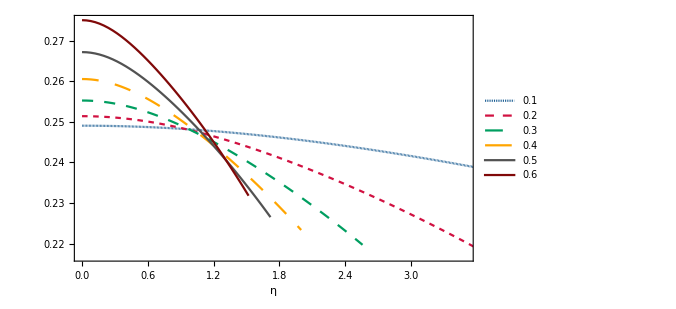

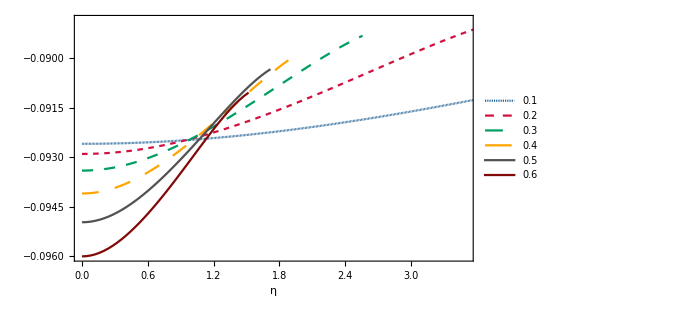

```mathematica
ListLinePlot[{Re[Tp1[[1]]],Re[Tp1[[2]]],Re[Tp1[[3]]],Re[Tp1[[4]]],Re[Tp1[[5]]],Re[Tp1[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.72}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[Tp1[[1]]],Im[Tp1[[2]]],Im[Tp1[[3]]],Im[Tp1[[4]]],Im[Tp1[[5]]],Im[Tp1[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
(Max[Re[Tdp1[[1]]]]-Min[Re[Tdp1[[1]]]])/Min[Re[Tdp1[[1]]]]*100
(Max[Im[Tdp1[[1]]]]-Min[Im[Tdp1[[1]]]])/Min[Im[Tdp1[[1]]]]*100
(Max[Re[Tdp1[[6]]]]-Min[Re[Tdp1[[6]]]])/Min[Re[Tdp1[[6]]]]*100
(Max[Im[Tdp1[[6]]]]-Min[Im[Tdp1[[6]]]])/Min[Im[Tdp1[[6]]]]*100
```

14.8246

-4.05464

18.6312

-5.17985

```mathematica
Min[Im[Tdp1][[1]]]
```

-0.0925909

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp1]-Re[Tda1])[[k]][[j+1]][[1]]/(Re[Tda1][[k]][[j+1]][[1]])*100+I*(Im[Tdp1]-Im[Tda1])[[k]][[j+1]][[1]]/(Abs[Im[Tda1][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

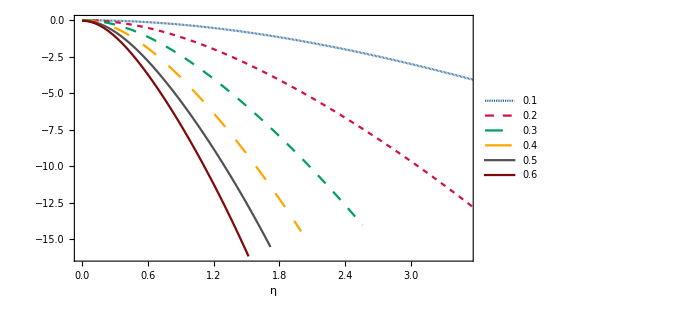

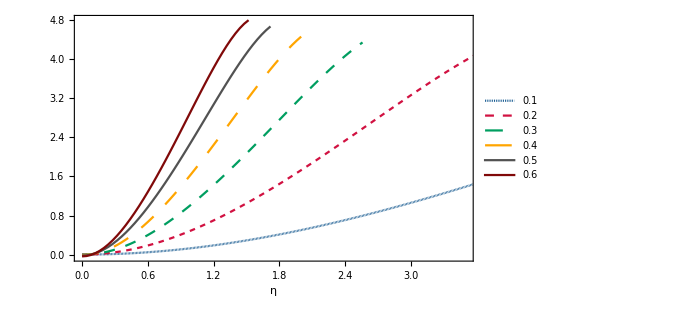

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.12,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.12,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
Max[Abs[(Max[Re[Tda1[[1]]]]-Min[Re[Tda1[[1]]]])/Min[Re[Tda1[[1]]]]*100],Abs[(Max[Re[Tda1[[2]]]]-Min[Re[Tda1[[2]]]])/Min[Re[Tda1[[2]]]]*100],Abs[(Max[Re[Tda1[[3]]]]-Min[Re[Tda1[[3]]]])/Min[Re[Tda1[[3]]]]*100],Abs[(Max[Re[Tda1[[4]]]]-Min[Re[Tda1[[4]]]])/Min[Re[Tda1[[4]]]]*100],Abs[(Max[Re[Tda1[[5]]]]-Min[Re[Tda1[[5]]]])/Min[Re[Tda1[[5]]]]*100],Abs[(Max[Re[Tda1[[6]]]]-Min[Re[Tda1[[6]]]])/Min[Re[Tda1[[6]]]]*100]]
Max[Abs[(Max[Im[Tda1[[1]]]]-Min[Im[Tda1[[1]]]])/Min[Im[Tda1[[1]]]]*100],Abs[(Max[Im[Tda1[[2]]]]-Min[Im[Tda1[[2]]]])/Min[Im[Tda1[[2]]]]*100],Abs[(Max[Im[Tda1[[3]]]]-Min[Im[Tda1[[3]]]])/Min[Im[Tda1[[3]]]]*100],Abs[(Max[Im[Tda1[[4]]]]-Min[Im[Tda1[[4]]]])/Min[Im[Tda1[[4]]]]*100],Abs[(Max[Im[Tda1[[5]]]]-Min[Im[Tda1[[5]]]])/Min[Im[Tda1[[5]]]]*100],Abs[(Max[Im[Tda1[[6]]]]-Min[Im[Tda1[[6]]]])/Min[Im[Tda1[[6]]]]*100]]
```

0.504529

0.363414

```mathematica
Max[Abs[(Max[Re[Tdp1[[1]]]]-Min[Re[Tdp1[[1]]]])/Min[Re[Tdp1[[1]]]]*100],Abs[(Max[Re[Tdp1[[2]]]]-Min[Re[Tdp1[[2]]]])/Min[Re[Tdp1[[2]]]]*100],Abs[(Max[Re[Tdp1[[3]]]]-Min[Re[Tdp1[[3]]]])/Min[Re[Tdp1[[3]]]]*100],Abs[(Max[Re[Tdp1[[4]]]]-Min[Re[Tdp1[[4]]]])/Min[Re[Tdp1[[4]]]]*100],Abs[(Max[Re[Tdp1[[5]]]]-Min[Re[Tdp1[[5]]]])/Min[Re[Tdp1[[5]]]]*100],Abs[(Max[Re[Tdp1[[6]]]]-Min[Re[Tdp1[[6]]]])/Min[Re[Tdp1[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp1[[1]]]]-Min[Im[Tdp1[[1]]]])/Min[Im[Tdp1[[1]]]]*100],Abs[(Max[Im[Tdp1[[2]]]]-Min[Im[Tdp1[[2]]]])/Min[Im[Tdp1[[2]]]]*100],Abs[(Max[Im[Tdp1[[3]]]]-Min[Im[Tdp1[[3]]]])/Min[Im[Tdp1[[3]]]]*100],Abs[(Max[Im[Tdp1[[4]]]]-Min[Im[Tdp1[[4]]]])/Min[Im[Tdp1[[4]]]]*100],Abs[(Max[Im[Tdp1[[5]]]]-Min[Im[Tdp1[[5]]]])/Min[Im[Tdp1[[5]]]]*100],Abs[(Max[Im[Tdp1[[6]]]]-Min[Im[Tdp1[[6]]]])/Min[Im[Tdp1[[6]]]]*100]]
```

18.6312

5.17985

#### Comparison between l=3 grav. & l=1 EM

Axial comparison

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tda1]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tda1]-Im[Tda])[[k]][[j+1]][[1]]/(Im[Tda][[k]][[j+1]][[1]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

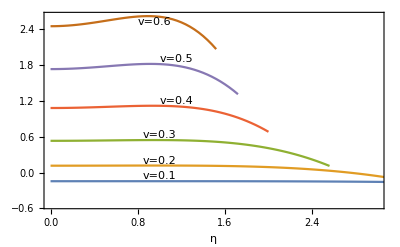

```mathematica
ListLinePlot[{Labeled[Im[DD[[1]]],"v=0.1",1],Labeled[Im[DD[[2]]],"v=0.2",1],Labeled[Im[DD[[3]]],"v=0.3",1],Labeled[Im[DD[[4]]],"v=0.4",1],Labeled[Im[DD[[5]]],"v=0.5",1],Labeled[Im[DD[[6]]],"v=0.6",0.8]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,3},Automatic}]
```

Polar Comparison

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp1]-Re[Tdp])[[k]][[j+1]][[1]]/(Re[Tdp][[k]][[j+1]][[1]])*100+I*(Im[Tdp1]-Im[Tdp])[[k]][[j+1]][[1]]/(Im[Tdp][[k]][[j+1]][[1]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

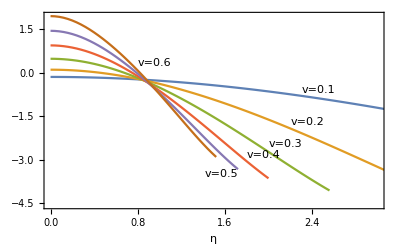

```mathematica
ListLinePlot[{Labeled[Im[DD[[1]]],"v=0.1",2.3],Labeled[Im[DD[[2]]],"v=0.2",2.2],Labeled[Im[DD[[3]]],"v=0.3",2],Labeled[Im[DD[[4]]],"v=0.4",1.8],Labeled[Im[DD[[5]]],"v=0.5",1.9],Labeled[Im[DD[[6]]],"v=0.6",0.8]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,3},Automatic}]
```

## l=2 EM mode axial & polar

#### Axial modes

```mathematica
Ta={{{0,0.45891692533497963-0.095096966292454 ⅈ},{1/25+ⅈ/25,0.4589169268582781-0.0950969659884937 ⅈ},{2/25+(2 ⅈ)/25,0.4589169314336775-0.09509696508029784 ⅈ},{3/25+(3 ⅈ)/25,0.45891693907767334-0.09509696357891931 ⅈ},{4/25+(4 ⅈ)/25,0.45891694981776143-0.09509696150277805 ⅈ},{1/5+ⅈ/5,0.4589169636924354-0.0950969588776661 ⅈ},{6/25+(6 ⅈ)/25,0.4589169807511974-0.09509695573672025 ⅈ},{7/25+(7 ⅈ)/25,0.45891700105454886-0.09509695212045381 ⅈ},{8/25+(8 ⅈ)/25,0.4589170246740005-0.09509694807673127 ⅈ},{9/25+(9 ⅈ)/25,0.4589170516920739-0.09509694366076842 ⅈ},{2/5+(2 ⅈ)/5,0.4589170822023059-0.09509693893512731 ⅈ},{11/25+(11 ⅈ)/25,0.4589171163092533-0.09509693396971033 ⅈ},{12/25+(12 ⅈ)/25,0.45891715412849754-0.09509692884175341 ⅈ},{13/25+(13 ⅈ)/25,0.4589171957866509-0.09509692363581859 ⅈ},{14/25+(14 ⅈ)/25,0.45891724142136214-0.09509691844378611 ⅈ},{3/5+(3 ⅈ)/5,0.45891729118132385-0.0950969133648453 ⅈ},{16/25+(16 ⅈ)/25,0.4589173452262795-0.09509690850548533 ⅈ},{17/25+(17 ⅈ)/25,0.45891740372703077-0.09509690397948461 ⅈ},{18/25+(18 ⅈ)/25,0.4589174668654467-0.0950968999079001 ⅈ},{19/25+(19 ⅈ)/25,0.4589175348344717-0.09509689641905521 ⅈ},{4/5+(4 ⅈ)/5,0.4589176078381355-0.09509689364852764 ⅈ},{21/25+(21 ⅈ)/25,0.4589176860915628-0.0950968917391359 ⅈ},{22/25+(22 ⅈ)/25,0.4589177698209837-0.09509689084092542 ⅈ},{23/25+(23 ⅈ)/25,0.4589178592637446-0.09509689111115373 ⅈ},{24/25+(24 ⅈ)/25,0.4589179546683196-0.09509689271427509 ⅈ},{1+ⅈ,0.4589180562943222-0.09509689582192406 ⅈ},{26/25+(26 ⅈ)/25,0.4589181644125182-0.09509690061289847 ⅈ},{27/25+(27 ⅈ)/25,0.4589182793048383-0.09509690727314159 ⅈ},{28/25+(28 ⅈ)/25,0.45891840126439126-0.0950969159957235 ⅈ},{29/25+(29 ⅈ)/25,0.45891853059547827-0.09509692698082166 ⅈ},{6/5+(6 ⅈ)/5,0.45891866761360695-0.09509694043570066 ⅈ},{31/25+(31 ⅈ)/25,0.45891881264550627-0.09509695657469112 ⅈ},{32/25+(32 ⅈ)/25,0.4589189660291422-0.0950969756191679 ⅈ},{33/25+(33 ⅈ)/25,0.45891912811373287-0.09509699779752727 ⅈ},{34/25+(34 ⅈ)/25,0.4589192992597652-0.09509702334516357 ⅈ},{7/5+(7 ⅈ)/5,0.45891947983901155-0.0950970525044445 ⅈ},{36/25+(36 ⅈ)/25,0.45891967023454683-0.09509708552468617 ⅈ},{37/25+(37 ⅈ)/25,0.45891987084076613-0.09509712266212678 ⅈ},{38/25+(38 ⅈ)/25,0.45892008206340246-0.09509716417989977 ⅈ},{39/25+(39 ⅈ)/25,0.45892030431954567-0.09509721034800572 ⅈ},{8/5+(8 ⅈ)/5,0.4589205380376609-0.09509726144328379 ⅈ},{41/25+(41 ⅈ)/25,0.45892078365760813-0.09509731774938186 ⅈ},{42/25+(42 ⅈ)/25,0.4589210416306617-0.09509737955672601 ⅈ},{43/25+(43 ⅈ)/25,0.45892131241953055-0.09509744716248893 ⅈ},{44/25+(44 ⅈ)/25,0.45892159649837855-0.09509752087055737 ⅈ},{9/5+(9 ⅈ)/5,0.45892189435284536-0.0950976009914988 ⅈ},{46/25+(46 ⅈ)/25,0.4589222064800678-0.09509768784252697 ⅈ},{47/25+(47 ⅈ)/25,0.45892253338870154-0.09509778174746647 ⅈ},{48/25+(48 ⅈ)/25,0.45892287559894274-0.09509788303671637 ⅈ},{49/25+(49 ⅈ)/25,0.45892323364255044-0.09509799204721278 ⅈ},{2+2 ⅈ,0.4589236080628696-0.09509810912239065 ⅈ},{51/25+(51 ⅈ)/25,0.45892399941485346-0.09509823461214403 ⅈ},{52/25+(52 ⅈ)/25,0.45892440826508724-0.09509836887278579 ⅈ},{53/25+(53 ⅈ)/25,0.45892483519181176-0.09509851226700602 ⅈ},{54/25+(54 ⅈ)/25,0.4589252807849469-0.09509866516382953 ⅈ},{11/5+(11 ⅈ)/5,0.4589257456461162-0.09509882793857197 ⅈ},{56/25+(56 ⅈ)/25,0.45892623038867114-0.09509900097279515 ⅈ},{57/25+(57 ⅈ)/25,0.458926735637716-0.09509918465426107 ⅈ},{58/25+(58 ⅈ)/25,0.45892726203013245-0.09509937937688502 ⅈ},{59/25+(59 ⅈ)/25,0.4589278102146048-0.09509958554068731 ⅈ},{12/5+(12 ⅈ)/5,0.45892838085164606-0.09509980355174383 ⅈ},{61/25+(61 ⅈ)/25,0.45892897461362236-0.09510003382213567 ⅈ},{62/25+(62 ⅈ)/25,0.45892959218477997-0.09510027676989745 ⅈ},{63/25+(63 ⅈ)/25,0.45893023426127033-0.0951005328189643 ⅈ},{64/25+(64 ⅈ)/25,0.4589309015511768-0.09510080239911783 ⅈ},{13/5+(13 ⅈ)/5,0.45893159477454054-0.0951010859459306 ⅈ},{66/25+(66 ⅈ)/25,0.45893231466338724-0.09510138390070969 ⅈ},{67/25+(67 ⅈ)/25,0.4589330619617535-0.09510169671043879 ⅈ},{68/25+(68 ⅈ)/25,0.45893383742571325-0.0951020248277189 ⅈ},{69/25+(69 ⅈ)/25,0.4589346418234051-0.09510236871070797 ⅈ},{14/5+(14 ⅈ)/5,0.4589354759350583-0.09510272882305905 ⅈ},{71/25+(71 ⅈ)/25,0.4589363405530204-0.09510310563385721 ⅈ},{72/25+(72 ⅈ)/25,0.4589372364817833-0.095103499617555 ⅈ},{73/25+(73 ⅈ)/25,0.45893816453801084-0.09510391125390665 ⅈ},{74/25+(74 ⅈ)/25,0.45893912555056493-0.09510434102790075 ⅈ},{3+3 ⅈ,0.4589401203605333-0.09510478942969179 ⅈ},{76/25+(76 ⅈ)/25,0.4589411498212552-0.09510525695452982 ⅈ},{77/25+(77 ⅈ)/25,0.458942214798349-0.09510574410268927 ⅈ},{78/25+(78 ⅈ)/25,0.4589433161697383-0.09510625137939567 ⅈ},{79/25+(79 ⅈ)/25,0.4589444548256786-0.09510677929475153 ⅈ},{16/5+(16 ⅈ)/5,0.45894563166878355-0.09510732836366015 ⅈ},{81/25+(81 ⅈ)/25,0.45894684761405136-0.09510789910574845 ⅈ},{82/25+(82 ⅈ)/25,0.4589481035888906-0.09510849204528775 ⅈ},{83/25+(83 ⅈ)/25,0.45894940053314626-0.0951091077111135 ⅈ},{84/25+(84 ⅈ)/25,0.45895073939912473-0.09510974663654312 ⅈ},{17/5+(17 ⅈ)/5,0.45895212115161993-0.0951104093592924 ⅈ},{86/25+(86 ⅈ)/25,0.45895354676793776-0.09511109642139026 ⅈ},{87/25+(87 ⅈ)/25,0.45895501723792104-0.09511180836909193 ⅈ},{88/25+(88 ⅈ)/25,0.4589565335639739-0.09511254575279046 ⅈ},{89/25+(89 ⅈ)/25,0.4589580967610854-0.09511330912692667 ⅈ},{18/5+(18 ⅈ)/5,0.4589597078568539-0.09511409904989733 ⅈ},{91/25+(91 ⅈ)/25,0.45896136789150965-0.09511491608396162 ⅈ},{92/25+(92 ⅈ)/25,0.45896307791793767-0.09511576079514622 ⅈ},{93/25+(93 ⅈ)/25,0.4589648390017-0.09511663375314819 ⅈ},{94/25+(94 ⅈ)/25,0.4589666522210575-0.09511753553123654 ⅈ},{19/5+(19 ⅈ)/5,0.45896851866699107-0.0951184667061519 ⅈ},{96/25+(96 ⅈ)/25,0.458970439443222-0.0951194278580043 ⅈ},{97/25+(97 ⅈ)/25,0.4589724156662325-0.09512041957016938 ⅈ},{98/25+(98 ⅈ)/25,0.4589744484652842-0.09512144242918273 ⅈ},{99/25+(99 ⅈ)/25,0.4589765389824377-0.09512249702463244 ⅈ},{4+4 ⅈ,0.45897868837256994-0.09512358394904978 ⅈ},{101/25+(101 ⅈ)/25,0.4589808978033917-0.09512470379779792 ⅈ},{102/25+(102 ⅈ)/25,0.4589831684554636-0.09512585716895931 ⅈ},{103/25+(103 ⅈ)/25,0.4589855015222123-0.09512704466322039 ⅈ},{104/25+(104 ⅈ)/25,0.45898789820994446-0.09512826688375522 ⅈ},{21/5+(21 ⅈ)/5,0.45899035973786123-0.09512952443610673 ⅈ},{106/25+(106 ⅈ)/25,0.45899288733807075-0.09513081792806614 ⅈ},{107/25+(107 ⅈ)/25,0.45899548225559994-0.0951321479695506 ⅈ},{108/25+(108 ⅈ)/25,0.45899814574840553-0.09513351517247885 ⅈ},{109/25+(109 ⅈ)/25,0.4590008790873838-0.0951349201506448 ⅈ},{22/5+(22 ⅈ)/5,0.4590036835563791-0.09513636351958933 ⅈ},{111/25+(111 ⅈ)/25,0.4590065604521916-0.09513784589647026 ⅈ},{112/25+(112 ⅈ)/25,0.45900951108458365-0.09513936789992973 ⅈ},{113/25+(113 ⅈ)/25,0.459012536776284-0.09514093014996057 ⅈ},{114/25+(114 ⅈ)/25,0.4590156388629929-0.09514253326776972 ⅈ},{23/5+(23 ⅈ)/5,0.4590188186933835-0.09514417787564028 ⅈ},{116/25+(116 ⅈ)/25,0.45902207762910335-0.09514586459679136 ⅈ},{117/25+(117 ⅈ)/25,0.4590254170447739-0.09514759405523587 ⅈ},{118/25+(118 ⅈ)/25,0.4590288383279886-0.09514936687563647 ⅈ},{119/25+(119 ⅈ)/25,0.4590323428793095-0.09515118368315913 ⅈ},{24/5+(24 ⅈ)/5,0.4590359321122624-0.09515304510332526 ⅈ},{121/25+(121 ⅈ)/25,0.4590396074533301-0.09515495176186123 ⅈ},{122/25+(122 ⅈ)/25,0.45904337034194415-0.09515690428454622 ⅈ},{123/25+(123 ⅈ)/25,0.45904722223047467-0.09515890329705785 ⅈ},{124/25+(124 ⅈ)/25,0.45905116458421863-0.09516094942481608 ⅈ},{5+5 ⅈ,0.45905519888138646-0.09516304329282457 ⅈ},{126/25+(126 ⅈ)/25,0.4590593266130858-0.09516518552551051 ⅈ},{127/25+(127 ⅈ)/25,0.4590635492833044-0.09516737674656223 ⅈ},{128/25+(128 ⅈ)/25,0.45906786840889063-0.09516961757876471 ⅈ},{129/25+(129 ⅈ)/25,0.45907228551953155-0.09517190864383325 ⅈ},{26/5+(26 ⅈ)/5,0.4590768021577294-0.09517425056224499 ⅈ},{131/25+(131 ⅈ)/25,0.4590814198787755-0.09517664395306845 ⅈ},{132/25+(132 ⅈ)/25,0.45908614025072225-0.09517908943379129 ⅈ},{133/25+(133 ⅈ)/25,0.4590909648543522-0.09518158762014567 ⅈ},{134/25+(134 ⅈ)/25,0.45909589528314576-0.0951841391259321 ⅈ},{27/5+(27 ⅈ)/5,0.45910093314324557-0.09518674456284103 ⅈ},{136/25+(136 ⅈ)/25,0.45910608005341863-0.09518940454027257 ⅈ},{137/25+(137 ⅈ)/25,0.45911133764501616-0.09519211966515444 ⅈ},{138/25+(138 ⅈ)/25,0.4591167075619306-0.09519489054175759 ⅈ},{139/25+(139 ⅈ)/25,0.45912219146055006-0.09519771777151063 ⅈ},{28/5+(28 ⅈ)/5,0.4591277910097094-0.09520060195281164 ⅈ},{141/25+(141 ⅈ)/25,0.4591335078906401-0.09520354368083865 ⅈ},{142/25+(142 ⅈ)/25,0.4591393437969151-0.095206543547358 ⅈ},{143/25+(143 ⅈ)/25,0.4591453004343924-0.09520960214053116 ⅈ},{144/25+(144 ⅈ)/25,0.45915137952115503-0.09521272004471958 ⅈ},{29/5+(29 ⅈ)/5,0.45915758278744784-0.09521589784028774 ⅈ},{146/25+(146 ⅈ)/25,0.4591639119756114-0.09521913610340484 ⅈ},{147/25+(147 ⅈ)/25,0.45917036884001244-0.09522243540584448 ⅈ},{148/25+(148 ⅈ)/25,0.4591769551469715-0.09522579631478259 ⅈ},{149/25+(149 ⅈ)/25,0.4591836726746864-0.09522921939259439 ⅈ},{6+6 ⅈ,0.45919052321315357-0.09523270519664889 ⅈ},{151/25+(151 ⅈ)/25,0.45919750856408426-0.09523625427910266 ⅈ},{152/25+(152 ⅈ)/25,0.459204630540819-0.09523986718669165 ⅈ},{153/25+(153 ⅈ)/25,0.459211890968237-0.09524354446052156 ⅈ},{154/25+(154 ⅈ)/25,0.45921929168266273-0.09524728663585721 ⅈ},{31/5+(31 ⅈ)/5,0.45922683453176844-0.09525109424191004 ⅈ},{156/25+(156 ⅈ)/25,0.4592345213744727-0.09525496780162489 ⅈ},{157/25+(157 ⅈ)/25,0.4592423540808357-0.09525890783146476 ⅈ},{158/25+(158 ⅈ)/25,0.45925033453194986-0.09526291484119537 ⅈ},{159/25+(159 ⅈ)/25,0.4592584646198268-0.0952669893336677 ⅈ},{32/5+(32 ⅈ)/5,0.4592667462472806-0.09527113180459999 ⅈ},{161/25+(161 ⅈ)/25,0.4592751813278061-0.09527534274235855 ⅈ},{162/25+(162 ⅈ)/25,0.45928377178545327-0.09527962262773763 ⅈ},{163/25+(163 ⅈ)/25,0.45929251955469835-0.09528397193373855 ⅈ},{164/25+(164 ⅈ)/25,0.45930142658030887-0.09528839112534784 ⅈ},{33/5+(33 ⅈ)/5,0.4593104948172056-0.09529288065931475 ⅈ},{166/25+(166 ⅈ)/25,0.4593197262303195-0.09529744098392813 ⅈ},{167/25+(167 ⅈ)/25,0.4593291227944447-0.0953020725387927 ⅈ},{168/25+(168 ⅈ)/25,0.4593386864940858-0.09530677575460479 ⅈ},{169/25+(169 ⅈ)/25,0.4593484193233019-0.0953115510529278 ⅈ},{34/5+(34 ⅈ)/5,0.4593583232855448-0.09531639884596708 ⅈ},{171/25+(171 ⅈ)/25,0.459368400393493-0.09532131953634497 ⅈ},{172/25+(172 ⅈ)/25,0.4593786526688813-0.09532631351687527 ⅈ},{173/25+(173 ⅈ)/25,0.459389082142324-0.09533138117033786 ⅈ},{174/25+(174 ⅈ)/25,0.4593996908531355-0.0953365228692534 ⅈ},{7+7 ⅈ,0.45941048084914365-0.09534173897565823 ⅈ},{176/25+(176 ⅈ)/25,0.45942145418649966-0.09534702984087907 ⅈ},{177/25+(177 ⅈ)/25,0.4594326129294822-0.09535239580530883 ⅈ},{178/25+(178 ⅈ)/25,0.4594439591502964-0.09535783719818207 ⅈ}},{{0,0.46281663668794343-0.09537012452061923 ⅈ},{1/25+ⅈ/25,0.462816660122627-0.09537011974288767 ⅈ},{2/25+(2 ⅈ)/25,0.4628167305101588-0.09537010546418694 ⅈ},{3/25+(3 ⅈ)/25,0.4628168481007633-0.09537008184802497 ⅈ},{4/25+(4 ⅈ)/25,0.46281701331157055-0.09537004916683456 ⅈ},{1/5+ⅈ/5,0.4628172267266676-0.09537000780186927 ⅈ},{6/25+(6 ⅈ)/25,0.462817489097204-0.0953699582430508 ⅈ},{7/25+(7 ⅈ)/25,0.46281780134152595-0.0953699010887723 ⅈ},{8/25+(8 ⅈ)/25,0.4628181645453413-0.09536983704565744 ⅈ},{9/25+(9 ⅈ)/25,0.46281857996191295-0.09536976692827462 ⅈ},{2/5+(2 ⅈ)/5,0.4628190490122818-0.09536969165880636 ⅈ},{11/25+(11 ⅈ)/25,0.46281957328551837-0.09536961226667254 ⅈ},{12/25+(12 ⅈ)/25,0.46282015453900244-0.09536952988810801 ⅈ},{13/25+(13 ⅈ)/25,0.4628207946987317-0.09536944576569274 ⅈ},{14/25+(14 ⅈ)/25,0.4628214958596569-0.09536936124783496 ⅈ},{3/5+(3 ⅈ)/5,0.4628222602860444-0.0953692777882054 ⅈ},{16/25+(16 ⅈ)/25,0.46282309041186587-0.09536919694512294 ⅈ},{17/25+(17 ⅈ)/25,0.4628239888412129-0.09536912038088953 ⅈ},{18/25+(18 ⅈ)/25,0.46282495834873755-0.09536904986107457 ⅈ},{19/25+(19 ⅈ)/25,0.4628260018801172-0.09536898725374712 ⅈ},{4/5+(4 ⅈ)/5,0.4628271225525433-0.09536893452865458 ⅈ},{21/25+(21 ⅈ)/25,0.4628283236552333-0.0953688937563476 ⅈ},{22/25+(22 ⅈ)/25,0.462829608649964-0.0953688671072489 ⅈ},{23/25+(23 ⅈ)/25,0.46283098117162663-0.09536885685066579 ⅈ},{24/25+(24 ⅈ)/25,0.46283244502880233-0.09536886535374424 ⅈ},{1+ⅈ,0.4628340042043557-0.09536889508036347 ⅈ},{26/25+(26 ⅈ)/25,0.4628356628560472-0.09536894858996976 ⅈ},{27/25+(27 ⅈ)/25,0.4628374253171617-0.0953690285363477 ⅈ},{28/25+(28 ⅈ)/25,0.46283929609715246-0.09536913766632739 ⅈ},{29/25+(29 ⅈ)/25,0.4628412798822996-0.09536927881842631 ⅈ},{6/5+(6 ⅈ)/5,0.46284338153638005-0.09536945492142375 ⅈ},{31/25+(31 ⅈ)/25,0.46284560610134956-0.09536966899286646 ⅈ},{32/25+(32 ⅈ)/25,0.4628479587980336-0.09536992413750378 ⅈ},{33/25+(33 ⅈ)/25,0.46285044502682554-0.09537022354565024 ⅈ},{34/25+(34 ⅈ)/25,0.4628530703683909-0.09537057049147407 ⅈ},{7/5+(7 ⅈ)/5,0.46285584058437573-0.0953709683312099 ⅈ},{36/25+(36 ⅈ)/25,0.46285876161811573-0.09537142050129342 ⅈ},{37/25+(37 ⅈ)/25,0.4628618395953463-0.09537193051641626 ⅈ},{38/25+(38 ⅈ)/25,0.46286508082490935-0.09537250196749951 ⅈ},{39/25+(39 ⅈ)/25,0.46286849179945466-0.09537313851958348 ⅈ},{8/5+(8 ⅈ)/5,0.46287207919613443-0.0953738439096321 ⅈ},{41/25+(41 ⅈ)/25,0.4628758498772874-0.09537462194424993 ⅈ},{42/25+(42 ⅈ)/25,0.4628798108911104-0.0953754764973096 ⅈ},{43/25+(43 ⅈ)/25,0.46288396947231375-0.09537641150748828 ⅈ},{44/25+(44 ⅈ)/25,0.4628883330427579-0.09537743097571064 ⅈ},{9/5+(9 ⅈ)/5,0.4628929092120685-0.09537853896249701 ⅈ},{46/25+(46 ⅈ)/25,0.4628977057782262-0.09537973958521424 ⅈ},{47/25+(47 ⅈ)/25,0.4629027307281274-0.09538103701522775 ⅈ},{48/25+(48 ⅈ)/25,0.46290799223811335-0.095382435474953 ⅈ},{49/25+(49 ⅈ)/25,0.46291349867446235-0.09538393923480444 ⅈ},{2+2 ⅈ,0.4629192585938434-0.09538555261004021 ⅈ},{51/25+(51 ⅈ)/25,0.4629252807437241-0.09538727995750128 ⅈ},{52/25+(52 ⅈ)/25,0.46293157406273194-0.0953891256722426 ⅈ},{53/25+(53 ⅈ)/25,0.46293814768096186-0.09539109418405617 ⅈ},{54/25+(54 ⅈ)/25,0.46294501092022744-0.09539318995388293 ⅈ},{11/5+(11 ⅈ)/5,0.46295217329424937-0.09539541747011362 ⅈ},{56/25+(56 ⅈ)/25,0.4629596445087774-0.09539778124477681 ⅈ},{57/25+(57 ⅈ)/25,0.4629674344616408-0.09540028580961263 ⅈ},{58/25+(58 ⅈ)/25,0.4629755532427201-0.0954029357120323 ⅈ},{59/25+(59 ⅈ)/25,0.46298401113383864-0.0954057355109618 ⅈ},{12/5+(12 ⅈ)/5,0.4629928186085631-0.09540868977256942 ⅈ},{61/25+(61 ⅈ)/25,0.4630019863319121-0.09541180306587713 ⅈ},{62/25+(62 ⅈ)/25,0.4630115251599632-0.09541507995825475 ⅈ},{63/25+(63 ⅈ)/25,0.46302144613935514-0.0954185250107979 ⅈ},{64/25+(64 ⅈ)/25,0.4630317605066762-0.09542214277358887 ⅈ},{13/5+(13 ⅈ)/5,0.4630424796877347-0.09542593778084223 ⅈ},{66/25+(66 ⅈ)/25,0.4630536152967031-0.09542991454593439 ⅈ},{67/25+(67 ⅈ)/25,0.46306517913513046-0.09543407755631954 ⅈ},{68/25+(68 ⅈ)/25,0.46307718319081487-0.09543843126833221 ⅈ},{69/25+(69 ⅈ)/25,0.46308963963653016-0.09544298010187882 ⅈ},{14/5+(14 ⅈ)/5,0.46310256082859824-0.09544772843501961 ⅈ},{71/25+(71 ⅈ)/25,0.4631159593053016-0.09545268059844386 ⅈ},{72/25+(72 ⅈ)/25,0.46312984778512645-0.0954578408698403 ⅈ},{73/25+(73 ⅈ)/25,0.46314423916483066-0.09546321346816673 ⅈ},{74/25+(74 ⅈ)/25,0.46315914651732804-0.0954688025478214 ⅈ},{3+3 ⅈ,0.4631745830893813-0.09547461219272078 ⅈ},{76/25+(76 ⅈ)/25,0.46319056229909683-0.0954806464102875 ⅈ},{77/25+(77 ⅈ)/25,0.4632070977332116-0.09548690912535368 ⅈ},{78/25+(78 ⅈ)/25,0.4632242031441678-0.09549340417398491 ⅈ},{79/25+(79 ⅈ)/25,0.4632418924469629-0.09550013529723007 ⅈ},{16/5+(16 ⅈ)/5,0.46326017971577255-0.09550710613480451 ⅈ},{81/25+(81 ⅈ)/25,0.46327907918033395-0.09551432021871178 ⅈ},{82/25+(82 ⅈ)/25,0.4632986052220855-0.09552178096681317 ⅈ},{83/25+(83 ⅈ)/25,0.4633187723700541-0.09552949167635108 ⅈ},{84/25+(84 ⅈ)/25,0.4633395952964829-0.09553745551743628 ⅈ},{17/5+(17 ⅈ)/5,0.4633610888121921-0.0955456755265075 ⅈ},{86/25+(86 ⅈ)/25,0.4633832678616669-0.09555415459977289 ⅈ},{87/25+(87 ⅈ)/25,0.4634061475178653-0.09556289548664378 ⅈ},{88/25+(88 ⅈ)/25,0.46342974297674006-0.09557190078317225 ⅈ},{89/25+(89 ⅈ)/25,0.4634540695514686-0.09558117292550312 ⅈ},{18/5+(18 ⅈ)/5,0.4634791426663851-0.09559071418335247 ⅈ},{91/25+(91 ⅈ)/25,0.46350497785061084-0.095600526653527 ⅈ}},{{0,0.4691208440906466-0.0958120715488743 ⅈ},{1/25+ⅈ/25,0.4691209559465481-0.09581204811948983 ⅈ},{2/25+(2 ⅈ)/25,0.4691212919013466-0.09581197807393685 ⅈ},{3/25+(3 ⅈ)/25,0.4691218531153383-0.09581186214001636 ⅈ},{4/25+(4 ⅈ)/25,0.46912264152298266-0.09581170152990698 ⅈ},{1/5+ⅈ/5,0.4691236598334561-0.09581149793901028 ⅈ},{6/25+(6 ⅈ)/25,0.4691249115315822-0.09581125354429589 ⅈ},{7/25+(7 ⅈ)/25,0.4691264008790203-0.09581097100216508 ⅈ},{8/25+(8 ⅈ)/25,0.46912813291570965-0.09581065344582654 ⅈ},{9/25+(9 ⅈ)/25,0.46913011346156286-0.09581030448217541 ⅈ},{2/5+(2 ⅈ)/5,0.4691323491184019-0.09580992818816722 ⅈ},{11/25+(11 ⅈ)/25,0.46913484727212895-0.09580952910667544 ⅈ},{12/25+(12 ⅈ)/25,0.46913761609512267-0.09580911224181984 ⅈ},{13/25+(13 ⅈ)/25,0.46914066454885056-0.09580868305375356 ⅈ},{14/25+(14 ⅈ)/25,0.4691440023866839-0.09580824745289239 ⅈ},{3/5+(3 ⅈ)/5,0.46914764015690497-0.095807811793571 ⅈ},{16/25+(16 ⅈ)/25,0.4691515892058892-0.09580738286710871 ⅈ},{17/25+(17 ⅈ)/25,0.46915586168144896-0.09580696789426572 ⅈ},{18/25+(18 ⅈ)/25,0.46916047053631993-0.09580657451707017 ⅈ},{19/25+(19 ⅈ)/25,0.4691654295317706-0.09580621078999532 ⅈ},{4/5+(4 ⅈ)/5,0.4691707532413156-0.09580588517046468 ⅈ},{21/25+(21 ⅈ)/25,0.46917645705450806-0.09580560650866239 ⅈ},{22/25+(22 ⅈ)/25,0.4691825571807884-0.09580538403662486 ⅈ},{23/25+(23 ⅈ)/25,0.46918907065335935-0.09580522735658945 ⅈ},{24/25+(24 ⅈ)/25,0.4691960153330619-0.09580514642857468 ⅈ},{1+ⅈ,0.46920340991221837-0.0958051515571665 ⅈ},{26/25+(26 ⅈ)/25,0.46921127391840894-0.09580525337748391 ⅈ},{27/25+(27 ⅈ)/25,0.46921962771814674-0.09580546284029803 ⅈ},{28/25+(28 ⅈ)/25,0.46922849252040927-0.09580579119627818 ⅈ},{29/25+(29 ⅈ)/25,0.4692378903799896-0.09580624997933683 ⅈ},{6/5+(6 ⅈ)/5,0.4692478442006162-0.09580685098904934 ⅈ},{31/25+(31 ⅈ)/25,0.4692583777377993-0.09580760627212104 ⅈ},{32/25+(32 ⅈ)/25,0.4692695156013481-0.09580852810287645 ⅈ},{33/25+(33 ⅈ)/25,0.46928128325750873-0.09580962896274758 ⅈ},{34/25+(34 ⅈ)/25,0.4692937070306623-0.09581092151873642 ⅈ},{7/5+(7 ⅈ)/5,0.4693068141045234-0.09581241860083142 ⅈ},{36/25+(36 ⅈ)/25,0.46932063252277423-0.09581413317835727 ⅈ},{37/25+(37 ⅈ)/25,0.4693351911890659-0.09581607833524049 ⅈ},{38/25+(38 ⅈ)/25,0.4693505198663155-0.09581826724417555 ⅈ},{39/25+(39 ⅈ)/25,0.46936664917522186-0.09582071313967894 ⅈ},{8/5+(8 ⅈ)/5,0.4693836105919232-0.09582342929002267 ⅈ},{41/25+(41 ⅈ)/25,0.4694014364447101-0.09582642896804064 ⅈ},{42/25+(42 ⅈ)/25,0.469420159909711-0.09582972542080814 ⅈ},{43/25+(43 ⅈ)/25,0.4694398150054551-0.09583333183819658 ⅈ},{44/25+(44 ⅈ)/25,0.46946043658622366-0.0958372613203128 ⅈ},{9/5+(9 ⅈ)/5,0.46948206033408796-0.0958415268438374 ⅈ},{46/25+(46 ⅈ)/25,0.46950472274953686-0.0958461412272819 ⅈ},{47/25+(47 ⅈ)/25,0.46952846114058777-0.0958511170951929 ⅈ},{48/25+(48 ⅈ)/25,0.4695533136102776-0.09585646684133782 ⅈ},{49/25+(49 ⅈ)/25,0.4695793190424222-0.09586220259091471 ⅈ},{2+2 ⅈ,0.4696065170855384-0.09586833616183796 ⅈ},{51/25+(51 ⅈ)/25,0.46963494813481216-0.09587487902516038 ⅈ},{52/25+(52 ⅈ)/25,0.4696646533120053-0.09588184226470195 ⅈ},{53/25+(53 ⅈ)/25,0.4696956744431814-0.09588923653596801 ⅈ},{54/25+(54 ⅈ)/25,0.4697280540341628-0.09589707202443713 ⅈ},{11/5+(11 ⅈ)/5,0.46976183524355475-0.09590535840335108 ⅈ},{56/25+(56 ⅈ)/25,0.46979706185329784-0.0959141047910826 ⅈ},{57/25+(57 ⅈ)/25,0.46983377823659433-0.0959233197082388 ⅈ},{58/25+(58 ⅈ)/25,0.4698720293231277-0.09593301103462774 ⅈ},{59/25+(59 ⅈ)/25,0.46991186056147866-0.09594318596624471 ⅈ},{12/5+(12 ⅈ)/5,0.46995331787864975-0.09595385097244413 ⅈ},{61/25+(61 ⅈ)/25,0.46999644763662074-0.09596501175347805 ⅈ},{62/25+(62 ⅈ)/25,0.47004129658586563-0.0959766731985943 ⅈ},{63/25+(63 ⅈ)/25,0.4700879118157738-0.09598883934490124 ⅈ},{64/25+(64 ⅈ)/25,0.47013634070193183-0.09600151333721918 ⅈ}},{{0,0.4775918137982794-0.09640710671217038 ⅈ},{1/25+ⅈ/25,0.47759214293227353-0.09640703611765648 ⅈ},{2/25+(2 ⅈ)/25,0.47759313141824383-0.09640682497555186 ⅈ},{3/25+(3 ⅈ)/25,0.4775947825053793-0.09640647520965373 ⅈ},{4/25+(4 ⅈ)/25,0.4775971016112583-0.09640599002209922 ⅈ},{1/5+ⅈ/5,0.47760009632407585-0.09640537388730518 ⅈ},{6/25+(6 ⅈ)/25,0.4776037764061901-0.09640463254334446 ⅈ},{7/25+(7 ⅈ)/25,0.4776081537986254-0.09640377298078918 ⅈ},{8/25+(8 ⅈ)/25,0.477613242626491-0.0964028034289698 ⅈ},{9/25+(9 ⅈ)/25,0.4776190592052599-0.09640173333958697 ⅈ},{2/5+(2 ⅈ)/5,0.47762562204784614-0.09640057336760356 ⅈ},{11/25+(11 ⅈ)/25,0.4776329518724046-0.096399335349333 ⅈ},{12/25+(12 ⅈ)/25,0.47764107161076563-0.09639803227763027 ⅈ},{13/25+(13 ⅈ)/25,0.4776500064174056-0.09639667827408256 ⅈ},{14/25+(14 ⅈ)/25,0.4776597836788399-0.09639528855808732 ⅈ},{3/5+(3 ⅈ)/5,0.47767043302331-0.09639387941269778 ⅈ},{16/25+(16 ⅈ)/25,0.4776819863306222-0.09639246814710736 ⅈ},{17/25+(17 ⅈ)/25,0.47769447774197854-0.0963910730556393 ⅈ},{18/25+(18 ⅈ)/25,0.47770794366962266-0.0963897133731007 ⅈ},{19/25+(19 ⅈ)/25,0.4777224228061051-0.09638840922635737 ⅈ},{4/5+(4 ⅈ)/5,0.4777379561329536-0.09638718158198172 ⅈ},{21/25+(21 ⅈ)/25,0.477754586928511-0.09638605218982477 ⅈ},{22/25+(22 ⅈ)/25,0.47777236077468344-0.09638504352236453 ⅈ},{23/25+(23 ⅈ)/25,0.47779132556231513-0.09638417870968399 ⅈ},{24/25+(24 ⅈ)/25,0.477811531494887-0.09638348146993773 ⅈ},{1+ⅈ,0.47783303109020164-0.09638297603517254 ⅈ},{26/25+(26 ⅈ)/25,0.47785587917969835-0.09638268707237749 ⅈ},{27/25+(27 ⅈ)/25,0.47788013290502623-0.09638263959965318 ⅈ},{28/25+(28 ⅈ)/25,0.47790585171140587-0.09638285889740052 ⅈ},{29/25+(29 ⅈ)/25,0.4779330973374281-0.09638337041446245 ⅈ},{6/5+(6 ⅈ)/5,0.47796193380072255-0.09638419966915818 ⅈ},{31/25+(31 ⅈ)/25,0.4779924273790486-0.09638537214519349 ⅈ},{32/25+(32 ⅈ)/25,0.4780246465862578-0.09638691318245655 ⅈ},{33/25+(33 ⅈ)/25,0.4780586621425661-0.0963888478627534 ⅈ},{34/25+(34 ⅈ)/25,0.4780945469385636-0.09639120089054654 ⅈ},{7/5+(7 ⅈ)/5,0.478132375992312-0.09639399646891247 ⅈ},{36/25+(36 ⅈ)/25,0.47817222639893936-0.0963972581708211 ⅈ},{37/25+(37 ⅈ)/25,0.4782141772720448-0.09640100880606706 ⅈ},{38/25+(38 ⅈ)/25,0.4782583096762539-0.09640527028415306 ⅈ},{39/25+(39 ⅈ)/25,0.478304706550243-0.09641006347353227 ⅈ},{8/5+(8 ⅈ)/5,0.4783534526195476-0.0964154080576931 ⅈ},{41/25+(41 ⅈ)/25,0.47840463429847346-0.09642132238865529 ⅈ},{42/25+(42 ⅈ)/25,0.47845833958044115-0.09642782333854098 ⅈ},{43/25+(43 ⅈ)/25,0.4785146579161171-0.09643492614998049 ⅈ},{44/25+(44 ⅈ)/25,0.4785736800787164-0.09644264428621635 ⅈ},{9/5+(9 ⅈ)/5,0.4786354980159073-0.09645098928187511 ⅈ},{46/25+(46 ⅈ)/25,0.47870020468780805-0.09645997059548524 ⅈ},{47/25+(47 ⅈ)/25,0.4787678938906395-0.09646959546492927 ⅈ},{48/25+(48 ⅈ)/25,0.47883866006568937-0.09647986876712773 ⅈ},{49/25+(49 ⅈ)/25,0.47891259809334913-0.09649079288335874 ⅈ},{2+2 ⅈ,0.4789898030721143-0.09650236757171812 ⅈ}},{{0,0.4879724438788044-0.09713888013214036 ⅈ},{1/25+ⅈ/25,0.4879731872832371-0.09713871859476148 ⅈ},{2/25+(2 ⅈ)/25,0.48797541976733216-0.09713823522385343 ⅈ},{3/25+(3 ⅈ)/25,0.48797914813713483-0.09713743374051302 ⅈ},{4/25+(4 ⅈ)/25,0.48798438374088415-0.09713632033225655 ⅈ},{1/5+ⅈ/5,0.4879911424735717-0.09713490363202777 ⅈ},{6/25+(6 ⅈ)/25,0.4879994447841879-0.09713319468840396 ⅈ},{7/25+(7 ⅈ)/25,0.48800931568473593-0.09713120692698478 ⅈ},{8/25+(8 ⅈ)/25,0.4880207847607818-0.09712895610273756 ⅈ},{9/25+(9 ⅈ)/25,0.48803388618324856-0.09712646024302803 ⅈ},{2/5+(2 ⅈ)/5,0.4880486587211075-0.09712373958102039 ⅈ},{11/25+(11 ⅈ)/25,0.488065145754551-0.09712081647908957 ⅈ},{12/25+(12 ⅈ)/25,0.48808339528816275-0.09711771534185243 ⅈ},{13/25+(13 ⅈ)/25,0.4881034599635299-0.09711446251839082 ⅈ},{14/25+(14 ⅈ)/25,0.48812539707066027-0.09711108619321215 ⅈ},{3/5+(3 ⅈ)/5,0.4881492685574844-0.09710761626547362 ⅈ},{16/25+(16 ⅈ)/25,0.4881751410366286-0.09710408421597898 ⅈ},{17/25+(17 ⅈ)/25,0.48820308578855204-0.09710052296145735 ⅈ},{18/25+(18 ⅈ)/25,0.48823317876003136-0.0970969666956329 ⅈ},{19/25+(19 ⅈ)/25,0.4882655005568723-0.09709345071662177 ⅈ},{4/5+(4 ⅈ)/5,0.4883001364296028-0.09709001124018085 ⅈ},{21/25+(21 ⅈ)/25,0.4883371762507941-0.09708668519849491 ⅈ},{22/25+(22 ⅈ)/25,0.4883767144825082-0.09708351002406478 ⅈ},{23/25+(23 ⅈ)/25,0.48841885013225855-0.09708052341852322 ⅈ},{24/25+(24 ⅈ)/25,0.4884636866957279-0.09707776310620396 ⅈ},{1+ⅈ,0.4885113320843496-0.09707526657245145 ⅈ},{26/25+(26 ⅈ)/25,0.4885618985357364-0.09707307078680996 ⅈ},{27/25+(27 ⅈ)/25,0.48861550250480007-0.0970712119114138 ⅈ},{28/25+(28 ⅈ)/25,0.4886722645332956-0.09706972499511624 ⅈ},{29/25+(29 ⅈ)/25,0.48873230909541093-0.09706864365414178 ⅈ},{6/5+(6 ⅈ)/5,0.488795764416933-0.09706799974033116 ⅈ},{31/25+(31 ⅈ)/25,0.48886276226545594-0.09706782299836646 ⅈ},{32/25+(32 ⅈ)/25,0.48893343770905956-0.09706814071371965 ⅈ},{33/25+(33 ⅈ)/25,0.4890079288408835-0.09706897735346183 ⅈ},{34/25+(34 ⅈ)/25,0.4890863764670731-0.0970703542024953 ⅈ},{7/5+(7 ⅈ)/5,0.48916892375566584-0.09707228899823293 ⅈ},{36/25+(36 ⅈ)/25,0.4892557158441557-0.0970747955672348 ⅈ},{37/25+(37 ⅈ)/25,0.48934689940370707-0.09707788346782228 ⅈ},{38/25+(38 ⅈ)/25,0.48944262215830664-0.09708155764321277 ⅈ},{39/25+(39 ⅈ)/25,0.4895430323575602-0.09708581809024178 ⅈ},{8/5+(8 ⅈ)/5,0.4896482782023475-0.09709065954925374 ⅈ},{41/25+(41 ⅈ)/25,0.4897585072231772-0.09709607122122826 ⅈ},{42/25+(42 ⅈ)/25,0.489873865611815-0.09710203651864793 ⅈ},{43/25+(43 ⅈ)/25,0.4899944975076153-0.0971085328569818 ⅈ}},{{0,0.500014881492248-0.09799213339755163 ⅈ},{1/25+ⅈ/25,0.5000163052720843-0.09799182485365726 ⅈ},{2/25+(2 ⅈ)/25,0.5000205805255843-0.09799090113001316 ⅈ},{3/25+(3 ⅈ)/25,0.5000277189813432-0.09798936794267363 ⅈ},{4/25+(4 ⅈ)/25,0.5000377401921539-0.09798723478063912 ⅈ},{1/5+ⅈ/5,0.5000506715373932-0.09798451485003054 ⅈ},{6/25+(6 ⅈ)/25,0.5000665482276909-0.0979812249949638 ⅈ},{7/25+(7 ⅈ)/25,0.5000854133097746-0.09797738559490428 ⅈ},{8/25+(8 ⅈ)/25,0.5001073176706042-0.09797302043783558 ⅈ},{9/25+(9 ⅈ)/25,0.5001323200396838-0.09796815656844945 ⅈ},{2/5+(2 ⅈ)/5,0.5001604869882004-0.09796282411045079 ⅈ},{11/25+(11 ⅈ)/25,0.5001918929233892-0.09795705606197645 ⅈ},{12/25+(12 ⅈ)/25,0.5002266200762485-0.09795088806305825 ⅈ},{13/25+(13 ⅈ)/25,0.500264758480426-0.09794435813396787 ⅈ},{14/25+(14 ⅈ)/25,0.500306405939818-0.09793750638339385 ⅈ},{3/5+(3 ⅈ)/5,0.500351667982022-0.09793037468521384 ⅈ},{16/25+(16 ⅈ)/25,0.5004006577944844-0.09792300632288897 ⅈ},{17/25+(17 ⅈ)/25,0.5004534961397664-0.09791544560050906 ⅈ},{18/25+(18 ⅈ)/25,0.5005103112459596-0.09790773741973008 ⅈ},{19/25+(19 ⅈ)/25,0.5005712386678619-0.09789992682208676 ⅈ},{4/5+(4 ⅈ)/5,0.500636421114098-0.09789205849648738 ⅈ},{21/25+(21 ⅈ)/25,0.5007060082349285-0.09788417625211382 ⅈ},{22/25+(22 ⅈ)/25,0.5007801563650738-0.09787632245746397 ⅈ},{23/25+(23 ⅈ)/25,0.5008590282154612-0.09786853744690116 ⅈ},{24/25+(24 ⅈ)/25,0.5009427925074383-0.09786085889682278 ⅈ},{1+ⅈ,0.5010316235426697-0.09785332117443919 ⅈ},{26/25+(26 ⅈ)/25,0.5011257007016986-0.09784595466317307 ⅈ},{27/25+(27 ⅈ)/25,0.5012252078640158-0.0978387850698473 ⅈ},{28/25+(28 ⅈ)/25,0.5013303327424836-0.09783183272013728 ⅈ},{29/25+(29 ⅈ)/25,0.5014412661251411-0.09782511185020656 ⅈ},{6/5+(6 ⅈ)/5,0.501558201017811-0.09781862990401848 ⅈ},{31/25+(31 ⅈ)/25,0.5016813316815851-0.09781238684749954 ⅈ},{32/25+(32 ⅈ)/25,0.501810852560224-0.09780637451249148 ⅈ},{33/25+(33 ⅈ)/25,0.5019469570938322-0.097800575985227 ⅈ},{34/25+(34 ⅈ)/25,0.5020898364168731-0.09779496505584453 ⅈ},{7/5+(7 ⅈ)/5,0.502239677940755-0.09778950574714194 ⅈ},{36/25+(36 ⅈ)/25,0.5023966638238359-0.09778415194227905 ⅈ},{37/25+(37 ⅈ)/25,0.5025609693348124-0.09777884713235627 ⅈ},{38/25+(38 ⅈ)/25,0.5027327611190481-0.09777352430561392 ⅈ}}};
```

```mathematica
Tda={{{0.45891692533497963-0.095096966292454 ⅈ},{0.4589169268582781-0.0950969659884937 ⅈ},{0.4589169314336775-0.09509696508029784 ⅈ},{0.45891693907767334-0.09509696357891931 ⅈ},{0.45891694981776143-0.09509696150277805 ⅈ},{0.4589169636924354-0.0950969588776661 ⅈ},{0.4589169807511974-0.09509695573672025 ⅈ},{0.45891700105454886-0.09509695212045381 ⅈ},{0.4589170246740005-0.09509694807673127 ⅈ},{0.4589170516920739-0.09509694366076842 ⅈ},{0.4589170822023059-0.09509693893512731 ⅈ},{0.4589171163092533-0.09509693396971033 ⅈ},{0.45891715412849754-0.09509692884175341 ⅈ},{0.4589171957866509-0.09509692363581859 ⅈ},{0.45891724142136214-0.09509691844378611 ⅈ},{0.45891729118132385-0.0950969133648453 ⅈ},{0.4589173452262795-0.09509690850548533 ⅈ},{0.45891740372703077-0.09509690397948461 ⅈ},{0.4589174668654467-0.0950968999079001 ⅈ},{0.4589175348344717-0.09509689641905521 ⅈ},{0.4589176078381355-0.09509689364852764 ⅈ},{0.4589176860915628-0.0950968917391359 ⅈ},{0.4589177698209837-0.09509689084092542 ⅈ},{0.4589178592637446-0.09509689111115373 ⅈ},{0.4589179546683196-0.09509689271427509 ⅈ},{0.4589180562943222-0.09509689582192406 ⅈ},{0.4589181644125182-0.09509690061289847 ⅈ},{0.4589182793048383-0.09509690727314159 ⅈ},{0.45891840126439126-0.0950969159957235 ⅈ},{0.45891853059547827-0.09509692698082166 ⅈ},{0.45891866761360695-0.09509694043570066 ⅈ},{0.45891881264550627-0.09509695657469112 ⅈ},{0.4589189660291422-0.0950969756191679 ⅈ},{0.45891912811373287-0.09509699779752727 ⅈ},{0.4589192992597652-0.09509702334516357 ⅈ},{0.45891947983901155-0.0950970525044445 ⅈ},{0.45891967023454683-0.09509708552468617 ⅈ},{0.45891987084076613-0.09509712266212678 ⅈ},{0.45892008206340246-0.09509716417989977 ⅈ},{0.45892030431954567-0.09509721034800572 ⅈ},{0.4589205380376609-0.09509726144328379 ⅈ},{0.45892078365760813-0.09509731774938186 ⅈ},{0.4589210416306617-0.09509737955672601 ⅈ},{0.45892131241953055-0.09509744716248893 ⅈ},{0.45892159649837855-0.09509752087055737 ⅈ},{0.45892189435284536-0.0950976009914988 ⅈ},{0.4589222064800678-0.09509768784252697 ⅈ},{0.45892253338870154-0.09509778174746647 ⅈ},{0.45892287559894274-0.09509788303671637 ⅈ},{0.45892323364255044-0.09509799204721278 ⅈ},{0.4589236080628696-0.09509810912239065 ⅈ},{0.45892399941485346-0.09509823461214403 ⅈ},{0.45892440826508724-0.09509836887278579 ⅈ},{0.45892483519181176-0.09509851226700602 ⅈ},{0.4589252807849469-0.09509866516382953 ⅈ},{0.4589257456461162-0.09509882793857197 ⅈ},{0.45892623038867114-0.09509900097279515 ⅈ},{0.458926735637716-0.09509918465426107 ⅈ},{0.45892726203013245-0.09509937937688502 ⅈ},{0.4589278102146048-0.09509958554068731 ⅈ},{0.45892838085164606-0.09509980355174383 ⅈ},{0.45892897461362236-0.09510003382213567 ⅈ},{0.45892959218477997-0.09510027676989745 ⅈ},{0.45893023426127033-0.0951005328189643 ⅈ},{0.4589309015511768-0.09510080239911783 ⅈ},{0.45893159477454054-0.0951010859459306 ⅈ},{0.45893231466338724-0.09510138390070969 ⅈ},{0.4589330619617535-0.09510169671043879 ⅈ},{0.45893383742571325-0.0951020248277189 ⅈ},{0.4589346418234051-0.09510236871070797 ⅈ},{0.4589354759350583-0.09510272882305905 ⅈ},{0.4589363405530204-0.09510310563385721 ⅈ},{0.4589372364817833-0.095103499617555 ⅈ},{0.45893816453801084-0.09510391125390665 ⅈ},{0.45893912555056493-0.09510434102790075 ⅈ},{0.4589401203605333-0.09510478942969179 ⅈ},{0.4589411498212552-0.09510525695452982 ⅈ},{0.458942214798349-0.09510574410268927 ⅈ},{0.4589433161697383-0.09510625137939567 ⅈ},{0.4589444548256786-0.09510677929475153 ⅈ},{0.45894563166878355-0.09510732836366015 ⅈ},{0.45894684761405136-0.09510789910574845 ⅈ},{0.4589481035888906-0.09510849204528775 ⅈ},{0.45894940053314626-0.0951091077111135 ⅈ},{0.45895073939912473-0.09510974663654312 ⅈ},{0.45895212115161993-0.0951104093592924 ⅈ},{0.45895354676793776-0.09511109642139026 ⅈ},{0.45895501723792104-0.09511180836909193 ⅈ},{0.4589565335639739-0.09511254575279046 ⅈ},{0.4589580967610854-0.09511330912692667 ⅈ},{0.4589597078568539-0.09511409904989733 ⅈ},{0.45896136789150965-0.09511491608396162 ⅈ},{0.45896307791793767-0.09511576079514622 ⅈ},{0.4589648390017-0.09511663375314819 ⅈ},{0.4589666522210575-0.09511753553123654 ⅈ},{0.45896851866699107-0.0951184667061519 ⅈ},{0.458970439443222-0.0951194278580043 ⅈ},{0.4589724156662325-0.09512041957016938 ⅈ},{0.4589744484652842-0.09512144242918273 ⅈ},{0.4589765389824377-0.09512249702463244 ⅈ},{0.45897868837256994-0.09512358394904978 ⅈ},{0.4589808978033917-0.09512470379779792 ⅈ},{0.4589831684554636-0.09512585716895931 ⅈ},{0.4589855015222123-0.09512704466322039 ⅈ},{0.45898789820994446-0.09512826688375522 ⅈ},{0.45899035973786123-0.09512952443610673 ⅈ},{0.45899288733807075-0.09513081792806614 ⅈ},{0.45899548225559994-0.0951321479695506 ⅈ},{0.45899814574840553-0.09513351517247885 ⅈ},{0.4590008790873838-0.0951349201506448 ⅈ},{0.4590036835563791-0.09513636351958933 ⅈ},{0.4590065604521916-0.09513784589647026 ⅈ},{0.45900951108458365-0.09513936789992973 ⅈ},{0.459012536776284-0.09514093014996057 ⅈ},{0.4590156388629929-0.09514253326776972 ⅈ},{0.4590188186933835-0.09514417787564028 ⅈ},{0.45902207762910335-0.09514586459679136 ⅈ},{0.4590254170447739-0.09514759405523587 ⅈ},{0.4590288383279886-0.09514936687563647 ⅈ},{0.4590323428793095-0.09515118368315913 ⅈ},{0.4590359321122624-0.09515304510332526 ⅈ},{0.4590396074533301-0.09515495176186123 ⅈ},{0.45904337034194415-0.09515690428454622 ⅈ},{0.45904722223047467-0.09515890329705785 ⅈ},{0.45905116458421863-0.09516094942481608 ⅈ},{0.45905519888138646-0.09516304329282457 ⅈ},{0.4590593266130858-0.09516518552551051 ⅈ},{0.4590635492833044-0.09516737674656223 ⅈ},{0.45906786840889063-0.09516961757876471 ⅈ},{0.45907228551953155-0.09517190864383325 ⅈ},{0.4590768021577294-0.09517425056224499 ⅈ},{0.4590814198787755-0.09517664395306845 ⅈ},{0.45908614025072225-0.09517908943379129 ⅈ},{0.4590909648543522-0.09518158762014567 ⅈ},{0.45909589528314576-0.0951841391259321 ⅈ},{0.45910093314324557-0.09518674456284103 ⅈ},{0.45910608005341863-0.09518940454027257 ⅈ},{0.45911133764501616-0.09519211966515444 ⅈ},{0.4591167075619306-0.09519489054175759 ⅈ},{0.45912219146055006-0.09519771777151063 ⅈ},{0.4591277910097094-0.09520060195281164 ⅈ},{0.4591335078906401-0.09520354368083865 ⅈ},{0.4591393437969151-0.095206543547358 ⅈ},{0.4591453004343924-0.09520960214053116 ⅈ},{0.45915137952115503-0.09521272004471958 ⅈ},{0.45915758278744784-0.09521589784028774 ⅈ},{0.4591639119756114-0.09521913610340484 ⅈ},{0.45917036884001244-0.09522243540584448 ⅈ},{0.4591769551469715-0.09522579631478259 ⅈ},{0.4591836726746864-0.09522921939259439 ⅈ},{0.45919052321315357-0.09523270519664889 ⅈ},{0.45919750856408426-0.09523625427910266 ⅈ},{0.459204630540819-0.09523986718669165 ⅈ},{0.459211890968237-0.09524354446052156 ⅈ},{0.45921929168266273-0.09524728663585721 ⅈ},{0.45922683453176844-0.09525109424191004 ⅈ},{0.4592345213744727-0.09525496780162489 ⅈ},{0.4592423540808357-0.09525890783146476 ⅈ},{0.45925033453194986-0.09526291484119537 ⅈ},{0.4592584646198268-0.0952669893336677 ⅈ},{0.4592667462472806-0.09527113180459999 ⅈ},{0.4592751813278061-0.09527534274235855 ⅈ},{0.45928377178545327-0.09527962262773763 ⅈ},{0.45929251955469835-0.09528397193373855 ⅈ},{0.45930142658030887-0.09528839112534784 ⅈ},{0.4593104948172056-0.09529288065931475 ⅈ},{0.4593197262303195-0.09529744098392813 ⅈ},{0.4593291227944447-0.0953020725387927 ⅈ},{0.4593386864940858-0.09530677575460479 ⅈ},{0.4593484193233019-0.0953115510529278 ⅈ},{0.4593583232855448-0.09531639884596708 ⅈ},{0.459368400393493-0.09532131953634497 ⅈ},{0.4593786526688813-0.09532631351687527 ⅈ},{0.459389082142324-0.09533138117033786 ⅈ},{0.4593996908531355-0.0953365228692534 ⅈ},{0.45941048084914365-0.09534173897565823 ⅈ},{0.45942145418649966-0.09534702984087907 ⅈ},{0.4594326129294822-0.09535239580530883 ⅈ},{0.4594439591502964-0.09535783719818207 ⅈ}},{{0.46281663668794343-0.09537012452061923 ⅈ},{0.462816660122627-0.09537011974288767 ⅈ},{0.4628167305101588-0.09537010546418694 ⅈ},{0.4628168481007633-0.09537008184802497 ⅈ},{0.46281701331157055-0.09537004916683456 ⅈ},{0.4628172267266676-0.09537000780186927 ⅈ},{0.462817489097204-0.0953699582430508 ⅈ},{0.46281780134152595-0.0953699010887723 ⅈ},{0.4628181645453413-0.09536983704565744 ⅈ},{0.46281857996191295-0.09536976692827462 ⅈ},{0.4628190490122818-0.09536969165880636 ⅈ},{0.46281957328551837-0.09536961226667254 ⅈ},{0.46282015453900244-0.09536952988810801 ⅈ},{0.4628207946987317-0.09536944576569274 ⅈ},{0.4628214958596569-0.09536936124783496 ⅈ},{0.4628222602860444-0.0953692777882054 ⅈ},{0.46282309041186587-0.09536919694512294 ⅈ},{0.4628239888412129-0.09536912038088953 ⅈ},{0.46282495834873755-0.09536904986107457 ⅈ},{0.4628260018801172-0.09536898725374712 ⅈ},{0.4628271225525433-0.09536893452865458 ⅈ},{0.4628283236552333-0.0953688937563476 ⅈ},{0.462829608649964-0.0953688671072489 ⅈ},{0.46283098117162663-0.09536885685066579 ⅈ},{0.46283244502880233-0.09536886535374424 ⅈ},{0.4628340042043557-0.09536889508036347 ⅈ},{0.4628356628560472-0.09536894858996976 ⅈ},{0.4628374253171617-0.0953690285363477 ⅈ},{0.46283929609715246-0.09536913766632739 ⅈ},{0.4628412798822996-0.09536927881842631 ⅈ},{0.46284338153638005-0.09536945492142375 ⅈ},{0.46284560610134956-0.09536966899286646 ⅈ},{0.4628479587980336-0.09536992413750378 ⅈ},{0.46285044502682554-0.09537022354565024 ⅈ},{0.4628530703683909-0.09537057049147407 ⅈ},{0.46285584058437573-0.0953709683312099 ⅈ},{0.46285876161811573-0.09537142050129342 ⅈ},{0.4628618395953463-0.09537193051641626 ⅈ},{0.46286508082490935-0.09537250196749951 ⅈ},{0.46286849179945466-0.09537313851958348 ⅈ},{0.46287207919613443-0.0953738439096321 ⅈ},{0.4628758498772874-0.09537462194424993 ⅈ},{0.4628798108911104-0.0953754764973096 ⅈ},{0.46288396947231375-0.09537641150748828 ⅈ},{0.4628883330427579-0.09537743097571064 ⅈ},{0.4628929092120685-0.09537853896249701 ⅈ},{0.4628977057782262-0.09537973958521424 ⅈ},{0.4629027307281274-0.09538103701522775 ⅈ},{0.46290799223811335-0.095382435474953 ⅈ},{0.46291349867446235-0.09538393923480444 ⅈ},{0.4629192585938434-0.09538555261004021 ⅈ},{0.4629252807437241-0.09538727995750128 ⅈ},{0.46293157406273194-0.0953891256722426 ⅈ},{0.46293814768096186-0.09539109418405617 ⅈ},{0.46294501092022744-0.09539318995388293 ⅈ},{0.46295217329424937-0.09539541747011362 ⅈ},{0.4629596445087774-0.09539778124477681 ⅈ},{0.4629674344616408-0.09540028580961263 ⅈ},{0.4629755532427201-0.0954029357120323 ⅈ},{0.46298401113383864-0.0954057355109618 ⅈ},{0.4629928186085631-0.09540868977256942 ⅈ},{0.4630019863319121-0.09541180306587713 ⅈ},{0.4630115251599632-0.09541507995825475 ⅈ},{0.46302144613935514-0.0954185250107979 ⅈ},{0.4630317605066762-0.09542214277358887 ⅈ},{0.4630424796877347-0.09542593778084223 ⅈ},{0.4630536152967031-0.09542991454593439 ⅈ},{0.46306517913513046-0.09543407755631954 ⅈ},{0.46307718319081487-0.09543843126833221 ⅈ},{0.46308963963653016-0.09544298010187882 ⅈ},{0.46310256082859824-0.09544772843501961 ⅈ},{0.4631159593053016-0.09545268059844386 ⅈ},{0.46312984778512645-0.0954578408698403 ⅈ},{0.46314423916483066-0.09546321346816673 ⅈ},{0.46315914651732804-0.0954688025478214 ⅈ},{0.4631745830893813-0.09547461219272078 ⅈ},{0.46319056229909683-0.0954806464102875 ⅈ},{0.4632070977332116-0.09548690912535368 ⅈ},{0.4632242031441678-0.09549340417398491 ⅈ},{0.4632418924469629-0.09550013529723007 ⅈ},{0.46326017971577255-0.09550710613480451 ⅈ},{0.46327907918033395-0.09551432021871178 ⅈ},{0.4632986052220855-0.09552178096681317 ⅈ},{0.4633187723700541-0.09552949167635108 ⅈ},{0.4633395952964829-0.09553745551743628 ⅈ},{0.4633610888121921-0.0955456755265075 ⅈ},{0.4633832678616669-0.09555415459977289 ⅈ},{0.4634061475178653-0.09556289548664378 ⅈ},{0.46342974297674006-0.09557190078317225 ⅈ},{0.4634540695514686-0.09558117292550312 ⅈ},{0.4634791426663851-0.09559071418335247 ⅈ},{0.46350497785061084-0.095600526653527 ⅈ}},{{0.4691208440906466-0.0958120715488743 ⅈ},{0.4691209559465481-0.09581204811948983 ⅈ},{0.4691212919013466-0.09581197807393685 ⅈ},{0.4691218531153383-0.09581186214001636 ⅈ},{0.46912264152298266-0.09581170152990698 ⅈ},{0.4691236598334561-0.09581149793901028 ⅈ},{0.4691249115315822-0.09581125354429589 ⅈ},{0.4691264008790203-0.09581097100216508 ⅈ},{0.46912813291570965-0.09581065344582654 ⅈ},{0.46913011346156286-0.09581030448217541 ⅈ},{0.4691323491184019-0.09580992818816722 ⅈ},{0.46913484727212895-0.09580952910667544 ⅈ},{0.46913761609512267-0.09580911224181984 ⅈ},{0.46914066454885056-0.09580868305375356 ⅈ},{0.4691440023866839-0.09580824745289239 ⅈ},{0.46914764015690497-0.095807811793571 ⅈ},{0.4691515892058892-0.09580738286710871 ⅈ},{0.46915586168144896-0.09580696789426572 ⅈ},{0.46916047053631993-0.09580657451707017 ⅈ},{0.4691654295317706-0.09580621078999532 ⅈ},{0.4691707532413156-0.09580588517046468 ⅈ},{0.46917645705450806-0.09580560650866239 ⅈ},{0.4691825571807884-0.09580538403662486 ⅈ},{0.46918907065335935-0.09580522735658945 ⅈ},{0.4691960153330619-0.09580514642857468 ⅈ},{0.46920340991221837-0.0958051515571665 ⅈ},{0.46921127391840894-0.09580525337748391 ⅈ},{0.46921962771814674-0.09580546284029803 ⅈ},{0.46922849252040927-0.09580579119627818 ⅈ},{0.4692378903799896-0.09580624997933683 ⅈ},{0.4692478442006162-0.09580685098904934 ⅈ},{0.4692583777377993-0.09580760627212104 ⅈ},{0.4692695156013481-0.09580852810287645 ⅈ},{0.46928128325750873-0.09580962896274758 ⅈ},{0.4692937070306623-0.09581092151873642 ⅈ},{0.4693068141045234-0.09581241860083142 ⅈ},{0.46932063252277423-0.09581413317835727 ⅈ},{0.4693351911890659-0.09581607833524049 ⅈ},{0.4693505198663155-0.09581826724417555 ⅈ},{0.46936664917522186-0.09582071313967894 ⅈ},{0.4693836105919232-0.09582342929002267 ⅈ},{0.4694014364447101-0.09582642896804064 ⅈ},{0.469420159909711-0.09582972542080814 ⅈ},{0.4694398150054551-0.09583333183819658 ⅈ},{0.46946043658622366-0.0958372613203128 ⅈ},{0.46948206033408796-0.0958415268438374 ⅈ},{0.46950472274953686-0.0958461412272819 ⅈ},{0.46952846114058777-0.0958511170951929 ⅈ},{0.4695533136102776-0.09585646684133782 ⅈ},{0.4695793190424222-0.09586220259091471 ⅈ},{0.4696065170855384-0.09586833616183796 ⅈ},{0.46963494813481216-0.09587487902516038 ⅈ},{0.4696646533120053-0.09588184226470195 ⅈ},{0.4696956744431814-0.09588923653596801 ⅈ},{0.4697280540341628-0.09589707202443713 ⅈ},{0.46976183524355475-0.09590535840335108 ⅈ},{0.46979706185329784-0.0959141047910826 ⅈ},{0.46983377823659433-0.0959233197082388 ⅈ},{0.4698720293231277-0.09593301103462774 ⅈ},{0.46991186056147866-0.09594318596624471 ⅈ},{0.46995331787864975-0.09595385097244413 ⅈ},{0.46999644763662074-0.09596501175347805 ⅈ},{0.47004129658586563-0.0959766731985943 ⅈ},{0.4700879118157738-0.09598883934490124 ⅈ},{0.47013634070193183-0.09600151333721918 ⅈ}},{{0.4775918137982794-0.09640710671217038 ⅈ},{0.47759214293227353-0.09640703611765648 ⅈ},{0.47759313141824383-0.09640682497555186 ⅈ},{0.4775947825053793-0.09640647520965373 ⅈ},{0.4775971016112583-0.09640599002209922 ⅈ},{0.47760009632407585-0.09640537388730518 ⅈ},{0.4776037764061901-0.09640463254334446 ⅈ},{0.4776081537986254-0.09640377298078918 ⅈ},{0.477613242626491-0.0964028034289698 ⅈ},{0.4776190592052599-0.09640173333958697 ⅈ},{0.47762562204784614-0.09640057336760356 ⅈ},{0.4776329518724046-0.096399335349333 ⅈ},{0.47764107161076563-0.09639803227763027 ⅈ},{0.4776500064174056-0.09639667827408256 ⅈ},{0.4776597836788399-0.09639528855808732 ⅈ},{0.47767043302331-0.09639387941269778 ⅈ},{0.4776819863306222-0.09639246814710736 ⅈ},{0.47769447774197854-0.0963910730556393 ⅈ},{0.47770794366962266-0.0963897133731007 ⅈ},{0.4777224228061051-0.09638840922635737 ⅈ},{0.4777379561329536-0.09638718158198172 ⅈ},{0.477754586928511-0.09638605218982477 ⅈ},{0.47777236077468344-0.09638504352236453 ⅈ},{0.47779132556231513-0.09638417870968399 ⅈ},{0.477811531494887-0.09638348146993773 ⅈ},{0.47783303109020164-0.09638297603517254 ⅈ},{0.47785587917969835-0.09638268707237749 ⅈ},{0.47788013290502623-0.09638263959965318 ⅈ},{0.47790585171140587-0.09638285889740052 ⅈ},{0.4779330973374281-0.09638337041446245 ⅈ},{0.47796193380072255-0.09638419966915818 ⅈ},{0.4779924273790486-0.09638537214519349 ⅈ},{0.4780246465862578-0.09638691318245655 ⅈ},{0.4780586621425661-0.0963888478627534 ⅈ},{0.4780945469385636-0.09639120089054654 ⅈ},{0.478132375992312-0.09639399646891247 ⅈ},{0.47817222639893936-0.0963972581708211 ⅈ},{0.4782141772720448-0.09640100880606706 ⅈ},{0.4782583096762539-0.09640527028415306 ⅈ},{0.478304706550243-0.09641006347353227 ⅈ},{0.4783534526195476-0.0964154080576931 ⅈ},{0.47840463429847346-0.09642132238865529 ⅈ},{0.47845833958044115-0.09642782333854098 ⅈ},{0.4785146579161171-0.09643492614998049 ⅈ},{0.4785736800787164-0.09644264428621635 ⅈ},{0.4786354980159073-0.09645098928187511 ⅈ},{0.47870020468780805-0.09645997059548524 ⅈ},{0.4787678938906395-0.09646959546492927 ⅈ},{0.47883866006568937-0.09647986876712773 ⅈ},{0.47891259809334913-0.09649079288335874 ⅈ},{0.4789898030721143-0.09650236757171812 ⅈ}},{{0.4879724438788044-0.09713888013214036 ⅈ},{0.4879731872832371-0.09713871859476148 ⅈ},{0.48797541976733216-0.09713823522385343 ⅈ},{0.48797914813713483-0.09713743374051302 ⅈ},{0.48798438374088415-0.09713632033225655 ⅈ},{0.4879911424735717-0.09713490363202777 ⅈ},{0.4879994447841879-0.09713319468840396 ⅈ},{0.48800931568473593-0.09713120692698478 ⅈ},{0.4880207847607818-0.09712895610273756 ⅈ},{0.48803388618324856-0.09712646024302803 ⅈ},{0.4880486587211075-0.09712373958102039 ⅈ},{0.488065145754551-0.09712081647908957 ⅈ},{0.48808339528816275-0.09711771534185243 ⅈ},{0.4881034599635299-0.09711446251839082 ⅈ},{0.48812539707066027-0.09711108619321215 ⅈ},{0.4881492685574844-0.09710761626547362 ⅈ},{0.4881751410366286-0.09710408421597898 ⅈ},{0.48820308578855204-0.09710052296145735 ⅈ},{0.48823317876003136-0.0970969666956329 ⅈ},{0.4882655005568723-0.09709345071662177 ⅈ},{0.4883001364296028-0.09709001124018085 ⅈ},{0.4883371762507941-0.09708668519849491 ⅈ},{0.4883767144825082-0.09708351002406478 ⅈ},{0.48841885013225855-0.09708052341852322 ⅈ},{0.4884636866957279-0.09707776310620396 ⅈ},{0.4885113320843496-0.09707526657245145 ⅈ},{0.4885618985357364-0.09707307078680996 ⅈ},{0.48861550250480007-0.0970712119114138 ⅈ},{0.4886722645332956-0.09706972499511624 ⅈ},{0.48873230909541093-0.09706864365414178 ⅈ},{0.488795764416933-0.09706799974033116 ⅈ},{0.48886276226545594-0.09706782299836646 ⅈ},{0.48893343770905956-0.09706814071371965 ⅈ},{0.4890079288408835-0.09706897735346183 ⅈ},{0.4890863764670731-0.0970703542024953 ⅈ},{0.48916892375566584-0.09707228899823293 ⅈ},{0.4892557158441557-0.0970747955672348 ⅈ},{0.48934689940370707-0.09707788346782228 ⅈ},{0.48944262215830664-0.09708155764321277 ⅈ},{0.4895430323575602-0.09708581809024178 ⅈ},{0.4896482782023475-0.09709065954925374 ⅈ},{0.4897585072231772-0.09709607122122826 ⅈ},{0.489873865611815-0.09710203651864793 ⅈ},{0.4899944975076153-0.0971085328569818 ⅈ}},{{0.500014881492248-0.09799213339755163 ⅈ},{0.5000163052720843-0.09799182485365726 ⅈ},{0.5000205805255843-0.09799090113001316 ⅈ},{0.5000277189813432-0.09798936794267363 ⅈ},{0.5000377401921539-0.09798723478063912 ⅈ},{0.5000506715373932-0.09798451485003054 ⅈ},{0.5000665482276909-0.0979812249949638 ⅈ},{0.5000854133097746-0.09797738559490428 ⅈ},{0.5001073176706042-0.09797302043783558 ⅈ},{0.5001323200396838-0.09796815656844945 ⅈ},{0.5001604869882004-0.09796282411045079 ⅈ},{0.5001918929233892-0.09795705606197645 ⅈ},{0.5002266200762485-0.09795088806305825 ⅈ},{0.500264758480426-0.09794435813396787 ⅈ},{0.500306405939818-0.09793750638339385 ⅈ},{0.500351667982022-0.09793037468521384 ⅈ},{0.5004006577944844-0.09792300632288897 ⅈ},{0.5004534961397664-0.09791544560050906 ⅈ},{0.5005103112459596-0.09790773741973008 ⅈ},{0.5005712386678619-0.09789992682208676 ⅈ},{0.500636421114098-0.09789205849648738 ⅈ},{0.5007060082349285-0.09788417625211382 ⅈ},{0.5007801563650738-0.09787632245746397 ⅈ},{0.5008590282154612-0.09786853744690116 ⅈ},{0.5009427925074383-0.09786085889682278 ⅈ},{0.5010316235426697-0.09785332117443919 ⅈ},{0.5011257007016986-0.09784595466317307 ⅈ},{0.5012252078640158-0.0978387850698473 ⅈ},{0.5013303327424836-0.09783183272013728 ⅈ},{0.5014412661251411-0.09782511185020656 ⅈ},{0.501558201017811-0.09781862990401848 ⅈ},{0.5016813316815851-0.09781238684749954 ⅈ},{0.501810852560224-0.09780637451249148 ⅈ},{0.5019469570938322-0.097800575985227 ⅈ},{0.5020898364168731-0.09779496505584453 ⅈ},{0.502239677940755-0.09778950574714194 ⅈ},{0.5023966638238359-0.09778415194227905 ⅈ},{0.5025609693348124-0.09777884713235627 ⅈ},{0.5027327611190481-0.09777352430561392 ⅈ}}};
```

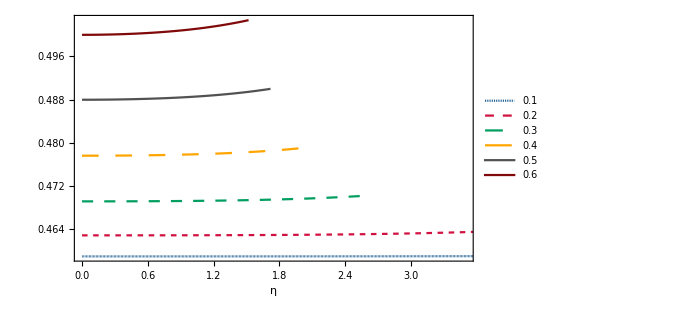

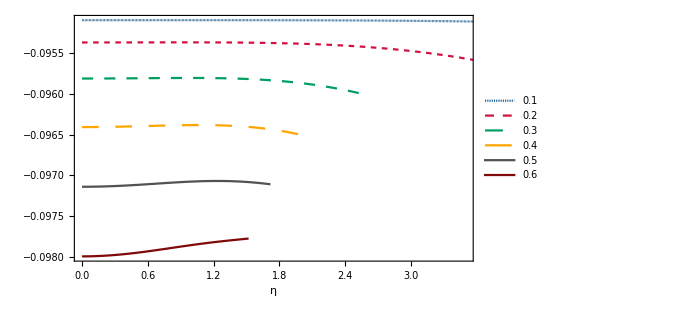

```mathematica
ListLinePlot[{Re[Ta[[1]]],Re[Ta[[2]]],Re[Ta[[3]]],Re[Ta[[4]]],Re[Ta[[5]]],Re[Ta[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[Ta[[1]]],Im[Ta[[2]]],Im[Ta[[3]]],Im[Ta[[4]]],Im[Ta[[5]]],Im[Ta[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100
(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100
(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100
(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100
```

0.114843

-0.27365

0.54356

-0.223088

#### Polar modes

```mathematica
Tp={{{0,0.45891647043383776-0.09509681018206584 ⅈ},{1/25+ⅈ/25,0.4589138967371133-0.09509663124270769 ⅈ},{2/25+(2 ⅈ)/25,0.45890617871819855-0.09509609461456887 ⅈ},{3/25+(3 ⅈ)/25,0.45889332559790136-0.09509520086813004 ⅈ},{4/25+(4 ⅈ)/25,0.4588753526778536-0.09509395095019411 ⅈ},{1/5+ⅈ/5,0.45885228125086924-0.09509234617856654 ⅈ},{6/25+(6 ⅈ)/25,0.4588241384736195-0.09509038823446185 ⅈ},{7/25+(7 ⅈ)/25,0.45879095720603097-0.09508807915292632 ⅈ},{8/25+(8 ⅈ)/25,0.45875277581949137-0.09508542131138634 ⅈ},{9/25+(9 ⅈ)/25,0.45870963797647957-0.0950824174164883 ⅈ},{2/5+(2 ⅈ)/5,0.4586615923844645-0.09507907048938902 ⅈ},{11/25+(11 ⅈ)/25,0.45860869252718806-0.09507538384968081 ⅈ},{12/25+(12 ⅈ)/25,0.4585509963766302-0.09507136109814926 ⅈ},{13/25+(13 ⅈ)/25,0.45848856608906075-0.0950670060985559 ⅈ},{14/25+(14 ⅈ)/25,0.4584214676886258-0.0950623229586576 ⅈ},{3/5+(3 ⅈ)/5,0.45834977074190175-0.09505731601066185 ⅈ},{16/25+(16 ⅈ)/25,0.4582735480267618-0.09505198979131597 ⅈ},{17/25+(17 ⅈ)/25,0.45819287519877167-0.09504634902182539 ⅈ},{18/25+(18 ⅈ)/25,0.4581078304581502-0.09504039858777909 ⅈ},{19/25+(19 ⅈ)/25,0.45801849422011287-0.0950341435192547 ⅈ},{4/5+(4 ⅈ)/5,0.4579249487911697-0.09502758897125649 ⅈ},{21/25+(21 ⅈ)/25,0.45782727805367934-0.0950207402046273 ⅈ},{22/25+(22 ⅈ)/25,0.4577255671606799-0.09501360256755731 ⅈ},{23/25+(23 ⅈ)/25,0.4576199022427267-0.09500618147779775 ⅈ},{24/25+(24 ⅈ)/25,0.45751037012817997-0.09499848240566787 ⅈ},{1+ⅈ,0.45739705807810316-0.09499051085792937 ⅈ},{26/25+(26 ⅈ)/25,0.45728005353666173-0.09498227236258573 ⅈ},{27/25+(27 ⅈ)/25,0.45715944389765545-0.09497377245464647 ⅈ},{28/25+(28 ⅈ)/25,0.45703531628758287-0.09496501666288772 ⅈ},{29/25+(29 ⅈ)/25,0.4569077573654195-0.09495601049761991 ⅈ},{6/5+(6 ⅈ)/5,0.4567768531390934-0.09494675943946768 ⅈ},{31/25+(31 ⅈ)/25,0.45664268879847975-0.09493726892915336 ⅈ},{32/25+(32 ⅈ)/25,0.4565053485645753-0.09492754435826785 ⅈ},{33/25+(33 ⅈ)/25,0.45636491555440134-0.09491759106100324 ⅈ},{34/25+(34 ⅈ)/25,0.4562214716610681-0.09490741430681647 ⅈ},{7/5+(7 ⅈ)/5,0.45607509744835845-0.09489701929398703 ⅈ},{36/25+(36 ⅈ)/25,0.4559258720591199-0.094886411144027 ⅈ},{37/25+(37 ⅈ)/25,0.4557738731367068-0.09487559489690157 ⅈ},{38/25+(38 ⅈ)/25,0.45561917675868485-0.09486457550700941 ⅈ},{39/25+(39 ⅈ)/25,0.4554618573819897-0.0948533578398798 ⅈ},{8/5+(8 ⅈ)/5,0.4553019877987281-0.09484194666953376 ⅈ},{41/25+(41 ⅈ)/25,0.4551396391018115-0.09483034667646396 ⅈ},{42/25+(42 ⅈ)/25,0.454974880659627-0.09481856244618225 ⅈ},{43/25+(43 ⅈ)/25,0.4548077800989721-0.09480659846829048 ⅈ},{44/25+(44 ⅈ)/25,0.4546384032955006-0.09479445913602698 ⅈ},{9/5+(9 ⅈ)/5,0.454466814370965-0.09478214874624637 ⅈ},{46/25+(46 ⅈ)/25,0.45429307569656785-0.094769671499789 ⅈ},{47/25+(47 ⅈ)/25,0.4541172479017776-0.09475703150219979 ⅈ},{48/25+(48 ⅈ)/25,0.45393938988799315-0.09474423276476196 ⅈ},{49/25+(49 ⅈ)/25,0.4537595588464931-0.09473127920580555 ⅈ},{2+2 ⅈ,0.4535778102801328-0.0947181746522606 ⅈ},{51/25+(51 ⅈ)/25,0.453394198028297-0.0947049228414225 ⅈ},{52/25+(52 ⅈ)/25,0.4532087742946525-0.09469152742290235 ⅈ},{53/25+(53 ⅈ)/25,0.4530215896772842-0.09467799196073438 ⅈ},{54/25+(54 ⅈ)/25,0.4528326932008281-0.09466431993561678 ⅈ},{11/5+(11 ⅈ)/5,0.45264213235025497-0.09465051474726398 ⅈ},{56/25+(56 ⅈ)/25,0.45244995310598596-0.09463657971685001 ⅈ},{57/25+(57 ⅈ)/25,0.45225619998005506-0.09462251808952377 ⅈ},{58/25+(58 ⅈ)/25,0.4520609160530584-0.09460833303698188 ⅈ},{59/25+(59 ⅈ)/25,0.45186414301166233-0.09459402766008038 ⅈ},{12/5+(12 ⅈ)/5,0.4516659211864604-0.09457960499147645 ⅈ},{61/25+(61 ⅈ)/25,0.4514662895899977-0.09456506799828455 ⅈ},{62/25+(62 ⅈ)/25,0.4512652859548021-0.09455041958473814 ⅈ},{63/25+(63 ⅈ)/25,0.45106294677127484-0.09453566259484739 ⅈ},{64/25+(64 ⅈ)/25,0.450859307325322-0.09452079981504392 ⅈ},{13/5+(13 ⅈ)/5,0.4506544017356137-0.0945058339768074 ⅈ},{66/25+(66 ⅈ)/25,0.4504482629903804-0.09449076775926372 ⅈ},{67/25+(67 ⅈ)/25,0.45024092298366486-0.09447560379175499 ⅈ},{68/25+(68 ⅈ)/25,0.45003241255096377-0.09446034465637146 ⅈ},{69/25+(69 ⅈ)/25,0.44982276150419986-0.09444499289044495 ⅈ},{14/5+(14 ⅈ)/5,0.44961199866598106-0.0944295509889985 ⅈ},{71/25+(71 ⅈ)/25,0.449400151903106-0.09441402140715123 ⅈ},{72/25+(72 ⅈ)/25,0.4491872481592868-0.0943984065624747 ⅈ},{73/25+(73 ⅈ)/25,0.4489733134870687-0.0943827088373004 ⅈ},{74/25+(74 ⅈ)/25,0.4487583730789239-0.09436693058097596 ⅈ},{3+3 ⅈ,0.4485424512975174-0.09435107411206996 ⅈ},{76/25+(76 ⅈ)/25,0.44832557170512943-0.09433514172052454 ⅈ},{77/25+(77 ⅈ)/25,0.4481077570922387-0.09431913566975522 ⅈ},{78/25+(78 ⅈ)/25,0.4478890295052675-0.0943030581986977 ⅈ},{79/25+(79 ⅈ)/25,0.4476694102734904-0.09428691152380315 ⅈ},{16/5+(16 ⅈ)/5,0.44744892003511777-0.09427069784098034 ⅈ},{81/25+(81 ⅈ)/25,0.4472275787625634-0.09425441932748634 ⅈ},{82/25+(82 ⅈ)/25,0.4470054057869082-0.09423807814376618 ⅈ},{83/25+(83 ⅈ)/25,0.4467824198215733-0.09422167643524165 ⅈ},{84/25+(84 ⅈ)/25,0.44655863898521886-0.09420521633405268 ⅈ},{17/5+(17 ⅈ)/5,0.44633408082388565-0.09418869996074618 ⅈ},{86/25+(86 ⅈ)/25,0.446108762332395-0.09417212942592156 ⅈ},{87/25+(87 ⅈ)/25,0.44588269997502744-0.0941555068318268 ⅈ},{88/25+(88 ⅈ)/25,0.44565590970549657-0.0941388342739099 ⅈ},{89/25+(89 ⅈ)/25,0.4454284069862394-0.09412211384232665 ⅈ},{18/5+(18 ⅈ)/5,0.4452002068070422-0.09410534762340364 ⅈ},{91/25+(91 ⅈ)/25,0.44497132370301934-0.09408853770106052 ⅈ},{92/25+(92 ⅈ)/25,0.4447417717719678-0.09407168615819048 ⅈ},{93/25+(93 ⅈ)/25,0.4445115646911154-0.09405479507800146 ⅈ},{94/25+(94 ⅈ)/25,0.4442807157332816-0.09403786654531751 ⅈ},{19/5+(19 ⅈ)/5,0.4440492377824711-0.09402090264784402 ⅈ},{96/25+(96 ⅈ)/25,0.44381714334892-0.09400390547739569 ⅈ},{97/25+(97 ⅈ)/25,0.4435844445836102-0.0939868771310887 ⅈ},{98/25+(98 ⅈ)/25,0.4433511532922747-0.0939698197124995 ⅈ},{99/25+(99 ⅈ)/25,0.44311728094890795-0.09395273533278915 ⅈ},{4+4 ⅈ,0.4428828387088007-0.09393562611179657 ⅈ},{101/25+(101 ⅈ)/25,0.4426478374211172-0.09391849417909964 ⅈ},{102/25+(102 ⅈ)/25,0.44241228764103013-0.09390134167504575 ⅈ},{103/25+(103 ⅈ)/25,0.4421761996414293-0.09388417075175365 ⅈ},{104/25+(104 ⅈ)/25,0.4419395834242219-0.09386698357408634 ⅈ},{21/5+(21 ⅈ)/5,0.44170244873123793-0.0938497823205961 ⅈ},{106/25+(106 ⅈ)/25,0.44146480505475666-0.09383256918444301 ⅈ},{107/25+(107 ⅈ)/25,0.4412266616476678-0.09381534637428644 ⅈ},{108/25+(108 ⅈ)/25,0.44098802753328237-0.09379811611515304 ⅈ},{109/25+(109 ⅈ)/25,0.440748911514806-0.09378088064927814 ⅈ},{22/5+(22 ⅈ)/5,0.44050932218448907-0.09376364223692395 ⅈ},{111/25+(111 ⅈ)/25,0.4402692679324636-0.09374640315717524 ⅈ},{112/25+(112 ⅈ)/25,0.44002875695528265-0.09372916570871082 ⅈ},{113/25+(113 ⅈ)/25,0.43978779726417133-0.0937119322105544 ⅈ},{114/25+(114 ⅈ)/25,0.4395463966930015-0.09369470500280358 ⅈ},{23/5+(23 ⅈ)/5,0.4393045629060033-0.09367748644733678 ⅈ},{116/25+(116 ⅈ)/25,0.43906230340521907-0.09366027892850082 ⅈ},{117/25+(117 ⅈ)/25,0.438819625537716-0.09364308485377904 ⅈ},{118/25+(118 ⅈ)/25,0.438576536502562-0.09362590665443775 ⅈ},{119/25+(119 ⅈ)/25,0.438333043357578-0.09360874678615526 ⅈ},{24/5+(24 ⅈ)/5,0.4380891530258731-0.09359160772963195 ⅈ},{121/25+(121 ⅈ)/25,0.4378448723021733-0.09357449199118044 ⅈ},{122/25+(122 ⅈ)/25,0.4376002078589507-0.09355740210330026 ⅈ},{123/25+(123 ⅈ)/25,0.4373551662523628-0.09354034062523121 ⅈ},{124/25+(124 ⅈ)/25,0.43710975392800805-0.09352331014349245 ⅈ},{5+5 ⅈ,0.4368639772265057-0.09350631327240191 ⅈ},{126/25+(126 ⅈ)/25,0.4366178423889085-0.09348935265458022 ⅈ},{127/25+(127 ⅈ)/25,0.43637135556195206-0.0934724309614359 ⅈ},{128/25+(128 ⅈ)/25,0.4361245228031518-0.09345555089363557 ⅈ},{129/25+(129 ⅈ)/25,0.4358773500857488-0.09343871518155657 ⅈ},{26/5+(26 ⅈ)/5,0.4356298433035161-0.09342192658572249 ⅈ},{131/25+(131 ⅈ)/25,0.43538200827542606-0.09340518789722353 ⅈ},{132/25+(132 ⅈ)/25,0.4351338507501887-0.09338850193811987 ⅈ},{133/25+(133 ⅈ)/25,0.4348853764106635-0.09337187156182808 ⅈ},{134/25+(134 ⅈ)/25,0.43463659087815243-0.09335529965349207 ⅈ},{27/5+(27 ⅈ)/5,0.43438749971657603-0.09333878913033766 ⅈ},{136/25+(136 ⅈ)/25,0.43413810843654144-0.09332234294201004 ⅈ},{137/25+(137 ⅈ)/25,0.4338884224993018-0.09330596407089517 ⅈ},{138/25+(138 ⅈ)/25,0.4336384473206175-0.09328965553242546 ⅈ},{139/25+(139 ⅈ)/25,0.43338818827451886-0.09327342037536758 ⅈ},{28/5+(28 ⅈ)/5,0.4331376506969746-0.09325726168209428 ⅈ},{141/25+(141 ⅈ)/25,0.4328868398894743-0.09324118256884013 ⅈ},{142/25+(142 ⅈ)/25,0.43263576112252305-0.0932251861859379 ⅈ},{143/25+(143 ⅈ)/25,0.43238441963905616-0.09320927571804129 ⅈ},{144/25+(144 ⅈ)/25,0.43213282065777375-0.09319345438432684 ⅈ},{29/5+(29 ⅈ)/5,0.4318809693764035-0.09317772543868076 ⅈ},{146/25+(146 ⅈ)/25,0.4316288709748892-0.09316209216986701 ⅈ},{147/25+(147 ⅈ)/25,0.4313765306185107-0.09314655790167697 ⅈ},{148/25+(148 ⅈ)/25,0.4311239534609406-0.09313112599306234 ⅈ},{149/25+(149 ⅈ)/25,0.43087114464723625-0.09311579983824722 ⅈ},{6+6 ⅈ,0.4306181093167716-0.09310058286682364 ⅈ},{151/25+(151 ⅈ)/25,0.4303648526061126-0.09308547854382525 ⅈ},{152/25+(152 ⅈ)/25,0.4301113796518376-0.09307049036978542 ⅈ},{153/25+(153 ⅈ)/25,0.42985769559330295-0.09305562188077009 ⅈ},{154/25+(154 ⅈ)/25,0.4296038055753618-0.0930408766483948 ⅈ},{31/5+(31 ⅈ)/5,0.4293497147510318-0.09302625827982003 ⅈ},{156/25+(156 ⅈ)/25,0.42909542828411834-0.09301177041772304 ⅈ},{157/25+(157 ⅈ)/25,0.42884095135179323-0.09299741674025082 ⅈ},{158/25+(158 ⅈ)/25,0.4285862891471317-0.09298320096095053 ⅈ},{159/25+(159 ⅈ)/25,0.42833144688160785-0.09296912682867646 ⅈ},{32/5+(32 ⅈ)/5,0.4280764297875534-0.09295519812747449 ⅈ},{161/25+(161 ⅈ)/25,0.4278212431205786-0.0929414186764432 ⅈ},{162/25+(162 ⅈ)/25,0.4275658921619574-0.09292779232957223 ⅈ},{163/25+(163 ⅈ)/25,0.4273103822209803-0.09291432297555284 ⅈ},{164/25+(164 ⅈ)/25,0.4270547186372738-0.09290101453756619 ⅈ},{33/5+(33 ⅈ)/5,0.4267989067830891-0.09288787097304564 ⅈ},{166/25+(166 ⅈ)/25,0.4265429520655618-0.09287489627341138 ⅈ},{167/25+(167 ⅈ)/25,0.42628685992894294-0.09286209446377933 ⅈ},{168/25+(168 ⅈ)/25,0.4260306358568024-0.09284946960264201 ⅈ},{169/25+(169 ⅈ)/25,0.4257742853742074-0.09283702578152143 ⅈ},{34/5+(34 ⅈ)/5,0.42551781404987515-0.09282476712459307 ⅈ},{171/25+(171 ⅈ)/25,0.42526122749830153-0.09281269778828033 ⅈ},{172/25+(172 ⅈ)/25,0.4250045313818676-0.09280082196081879 ⅈ},{173/25+(173 ⅈ)/25,0.4247477314129227-0.09278914386178949 ⅈ},{174/25+(174 ⅈ)/25,0.4244908333558478-0.09277766774161975 ⅈ},{7+7 ⅈ,0.42423384302909634-0.09276639788105408 ⅈ},{176/25+(176 ⅈ)/25,0.42397676630721703-0.09275533859058846 ⅈ},{177/25+(177 ⅈ)/25,0.42371960912285644-0.09274449420987306 ⅈ},{178/25+(178 ⅈ)/25,0.4234623774687437-0.0927338691070791 ⅈ}},{{0,0.4628097165789426-0.09536774384978551 ⅈ},{1/25+ⅈ/25,0.4627990908411818-0.09536702186553662 ⅈ},{2/25+(2 ⅈ)/25,0.46276726957118214-0.0953648592001967 ⅈ},{3/25+(3 ⅈ)/25,0.46271441922391643-0.09536126564103117 ⅈ},{4/25+(4 ⅈ)/25,0.46264081235954896-0.09535625722976303 ⅈ},{1/5+ⅈ/5,0.4625468206894699-0.09534985587573144 ⅈ},{6/25+(6 ⅈ)/25,0.46243290590441666-0.09534208884403093 ⅈ},{7/25+(7 ⅈ)/25,0.46229960880137716-0.09533298814644266 ⅈ},{8/25+(8 ⅈ)/25,0.46214753726939845-0.0953225898653782 ⅈ},{9/25+(9 ⅈ)/25,0.46197735370022897-0.09531093344171011 ⅈ},{2/5+(2 ⅈ)/5,0.46178976235298946-0.09529806095574046 ⅈ},{11/25+(11 ⅈ)/25,0.46158549713272606-0.0952840164271655 ⅈ},{12/25+(12 ⅈ)/25,0.4613653101526552-0.09526884515528888 ⅈ},{13/25+(13 ⅈ)/25,0.4611299613510436-0.09525259311555108 ⅈ},{14/25+(14 ⅈ)/25,0.4608802093362184-0.09523530642318632 ⅈ},{3/5+(3 ⅈ)/5,0.4606168035448476-0.09521703086994784 ⅈ},{16/25+(16 ⅈ)/25,0.4603404777242422-0.09519781153562894 ⅈ},{17/25+(17 ⅈ)/25,0.46005194469123045-0.09517769247270826 ⅈ},{18/25+(18 ⅈ)/25,0.459751892278249-0.09515671645990548 ⅈ},{19/25+(19 ⅈ)/25,0.45944098035032505-0.09513492481870212 ⅈ},{4/5+(4 ⅈ)/5,0.4591198387623295-0.09511235728586206 ⅈ},{21/25+(21 ⅈ)/25,0.45878906612165926-0.09508905193455139 ⅈ},{22/25+(22 ⅈ)/25,0.45844922922475-0.0950650451366707 ⅈ},{23/25+(23 ⅈ)/25,0.45810086304419506-0.09504037155935023 ⅈ},{24/25+(24 ⅈ)/25,0.45774447115475375-0.09501506418910959 ⅈ},{1+ⅈ,0.457380526499642-0.09498915437785603 ⅈ},{26/25+(26 ⅈ)/25,0.45700947241202566-0.09496267190561959 ⅈ},{27/25+(27 ⅈ)/25,0.45663172381979594-0.0949356450556517 ⅈ},{28/25+(28 ⅈ)/25,0.45624766857395255-0.09490810069820424 ⅈ},{29/25+(29 ⅈ)/25,0.4558576688519794-0.09488006437994799 ⅈ},{6/5+(6 ⅈ)/5,0.455462062597313-0.09485156041655561 ⅈ},{31/25+(31 ⅈ)/25,0.45506116496438853-0.09482261198647697 ⅈ},{32/25+(32 ⅈ)/25,0.45465526974582066-0.09479324122436428 ⅈ},{33/25+(33 ⅈ)/25,0.45424465076419107-0.0947634693129651 ⅈ},{34/25+(34 ⅈ)/25,0.4538295632157406-0.09473331657260217 ⅈ},{7/5+(7 ⅈ)/5,0.4534102449571984-0.09470280254760974 ⅈ},{36/25+(36 ⅈ)/25,0.4529869177300925-0.09467194608929207 ⅈ},{37/25+(37 ⅈ)/25,0.45255978831936094-0.09464076543513238 ⅈ},{38/25+(38 ⅈ)/25,0.45212904964497663-0.0946092782841061 ⅈ},{39/25+(39 ⅈ)/25,0.45169488178675876-0.09457750186804752 ⅈ},{8/5+(8 ⅈ)/5,0.45125745294361896-0.09454545301909409 ⅈ},{41/25+(41 ⅈ)/25,0.45081692032927223-0.09451314823328967 ⅈ},{42/25+(42 ⅈ)/25,0.4503734310069887-0.09448060373046271 ⅈ},{43/25+(43 ⅈ)/25,0.4499271226663244-0.09444783551052702 ⅈ},{44/25+(44 ⅈ)/25,0.44947812434497714-0.0944148594063669 ⅈ},{9/5+(9 ⅈ)/5,0.4490265570990213-0.09438169113348198 ⅈ},{46/25+(46 ⅈ)/25,0.4485725346247919-0.09434834633656597 ⅈ},{47/25+(47 ⅈ)/25,0.4481161638356465-0.09431484063319927 ⅈ},{48/25+(48 ⅈ)/25,0.44765754539674085-0.09428118965482504 ⅈ},{49/25+(49 ⅈ)/25,0.44719677422084275-0.09424740908517862 ⅈ},{2+2 ⅈ,0.44673393992805704-0.09421351469632736 ⅈ},{51/25+(51 ⅈ)/25,0.44626912727219026-0.09417952238247104 ⅈ},{52/25+(52 ⅈ)/25,0.44580241653631925-0.09414544819164272 ⅈ},{53/25+(53 ⅈ)/25,0.4453338838999662-0.09411130835544075 ⅈ},{54/25+(54 ⅈ)/25,0.44486360178012435-0.09407711931691025 ⅈ},{11/5+(11 ⅈ)/5,0.4443916391482201-0.09404289775668251 ⅈ},{56/25+(56 ⅈ)/25,0.4439180618249499-0.09400866061747494 ⅈ},{57/25+(57 ⅈ)/25,0.443442932754785-0.0939744251270339 ⅈ},{58/25+(58 ⅈ)/25,0.44296631226179933-0.09394020881960681 ⅈ},{59/25+(59 ⅈ)/25,0.44248825828835675-0.09390602955600838 ⅈ},{12/5+(12 ⅈ)/5,0.44200882661806207-0.09387190554234359 ⅈ},{61/25+(61 ⅈ)/25,0.44152807108427977-0.09383785534744148 ⅈ},{62/25+(62 ⅈ)/25,0.4410460437654162-0.09380389791904178 ⅈ},{63/25+(63 ⅈ)/25,0.4405627951680635-0.09377005259877165 ⅈ},{64/25+(64 ⅈ)/25,0.4400783743990192-0.09373633913594187 ⅈ},{13/5+(13 ⅈ)/5,0.4395928293271107-0.09370277770018434 ⅈ},{66/25+(66 ⅈ)/25,0.43910620673567946-0.09366938889294477 ⅈ},{67/25+(67 ⅈ)/25,0.43861855246650927-0.09363619375784074 ⅈ},{68/25+(68 ⅈ)/25,0.43812991155591996-0.09360321378988477 ⅈ},{69/25+(69 ⅈ)/25,0.43764032836368943-0.09357047094357032 ⅈ},{14/5+(14 ⅈ)/5,0.4371498466954119-0.09353798763980965 ⅈ},{71/25+(71 ⅈ)/25,0.4366585099188506-0.0935057867717082 ⅈ},{72/25+(72 ⅈ)/25,0.43616636107479684-0.09347389170915214 ⅈ},{73/25+(73 ⅈ)/25,0.43567344298290733-0.09344232630218585 ⅈ},{74/25+(74 ⅈ)/25,0.43517979834295056-0.09341111488314359 ⅈ},{3+3 ⅈ,0.43468546983185713-0.09338028226750052 ⅈ},{76/25+(76 ⅈ)/25,0.43419050019693767-0.09334985375339831 ⅈ},{77/25+(77 ⅈ)/25,0.4336949323455982-0.09331985511979982 ⅈ},{78/25+(78 ⅈ)/25,0.43319880943185846-0.09329031262321921 ⅈ},{79/25+(79 ⅈ)/25,0.4327021749399473-0.0932612529929715 ⅈ},{16/5+(16 ⅈ)/5,0.4322050727652285-0.0932327034248756 ⅈ},{81/25+(81 ⅈ)/25,0.4317075472926849-0.09320469157335212 ⅈ},{82/25+(82 ⅈ)/25,0.4312096434731668-0.09317724554183356 ⅈ},{83/25+(83 ⅈ)/25,0.43071140689759363-0.09315039387142066 ⅈ},{84/25+(84 ⅈ)/25,0.43021288386926965-0.09312416552769959 ⅈ},{17/5+(17 ⅈ)/5,0.42971412147446914-0.09309858988563541 ⅈ},{86/25+(86 ⅈ)/25,0.4292151676514147-0.09307369671245488 ⅈ},{87/25+(87 ⅈ)/25,0.42871607125776545-0.09304951614842313 ⅈ},{88/25+(88 ⅈ)/25,0.4282168821367102-0.09302607868541916 ⅈ},{89/25+(89 ⅈ)/25,0.427717651181745-0.09300341514320846 ⅈ},{18/5+(18 ⅈ)/5,0.4272184304002025-0.09298155664330893 ⅈ},{91/25+(91 ⅈ)/25,0.42671927297557793-0.09296053458034083 ⅈ}},{{0,0.4690884012753177-0.09580086198110876 ⅈ},{1/25+ⅈ/25,0.4690630850432939-0.09579921508810389 ⅈ},{2/25+(2 ⅈ)/25,0.46898748860649153-0.0957942931059144 ⅈ},{3/25+(3 ⅈ)/25,0.46886264480875234-0.09578615098942732 ⅈ},{4/25+(4 ⅈ)/25,0.46869019815145935-0.09577487664745865 ⅈ},{1/5+ⅈ/5,0.46847230167512927-0.09576058594749251 ⅈ},{6/25+(6 ⅈ)/25,0.468211493613506-0.09574341664203725 ⅈ},{7/25+(7 ⅈ)/25,0.4679105686134999-0.0957235218942084 ⅈ},{8/25+(8 ⅈ)/25,0.4675724561384503-0.0957010640106855 ⅈ},{9/25+(9 ⅈ)/25,0.46720011488817603-0.09567620884170534 ⅈ},{2/5+(2 ⅈ)/5,0.466796447906874-0.09564912112752459 ⅈ},{11/25+(11 ⅈ)/25,0.4663642394507259-0.095619960900991 ⅈ},{12/25+(12 ⅈ)/25,0.4659061121210808-0.09558888092265577 ⅈ},{13/25+(13 ⅈ)/25,0.46542450129617896-0.09555602503758687 ⅈ},{14/25+(14 ⅈ)/25,0.4649216433251595-0.09552152729844357 ⅈ},{3/5+(3 ⅈ)/5,0.4643995740012571-0.09548551168772879 ⅈ},{16/25+(16 ⅈ)/25,0.4638601342390109-0.09544809228202462 ⅈ},{17/25+(17 ⅈ)/25,0.4633049804379552-0.09540937372251229 ⅈ},{18/25+(18 ⅈ)/25,0.4627355975891522-0.09536945188181957 ⅈ},{19/25+(19 ⅈ)/25,0.46215331369774676-0.09532841464256707 ⅈ},{4/5+(4 ⅈ)/5,0.46155931452350407-0.09528634272542 ⅈ},{21/25+(21 ⅈ)/25,0.46095465797699053-0.095243310522968 ⅈ},{22/25+(22 ⅈ)/25,0.4603402877602412-0.09519938691029324 ⅈ},{23/25+(23 ⅈ)/25,0.4597170460215138-0.09515463601403397 ⅈ},{24/25+(24 ⅈ)/25,0.4590856849191064-0.09510911792969994 ⅈ},{1+ⅈ,0.45844687707280024-0.09506288938257518 ⅈ},{26/25+(26 ⅈ)/25,0.45780122493463876-0.09501600433130541 ⅈ},{27/25+(27 ⅈ)/25,0.4571492691423379-0.0949685145156987 ⅈ},{28/25+(28 ⅈ)/25,0.4564914959353998-0.09492046995172823 ⅈ},{29/25+(29 ⅈ)/25,0.4558283437208813-0.09487191937752357 ⅈ},{6/5+(6 ⅈ)/5,0.45516020887628755-0.09482291065446927 ⅈ},{31/25+(31 ⅈ)/25,0.454487450873684-0.09477349112755981 ⅈ},{32/25+(32 ⅈ)/25,0.45381039680351964-0.09472370794900765 ⅈ},{33/25+(33 ⅈ)/25,0.45312934536996885-0.09467360836882177 ⅈ},{34/25+(34 ⅈ)/25,0.4524445704225408-0.09462323999575223 ⅈ},{7/5+(7 ⅈ)/5,0.45175632408174754-0.09457265103162865 ⅈ},{36/25+(36 ⅈ)/25,0.451064839510006-0.09452189048176939 ⅈ},{37/25+(37 ⅈ)/25,0.45037033337285964-0.09447100834378529 ⅈ},{38/25+(38 ⅈ)/25,0.44967300803005483-0.09442005577677044 ⅈ},{39/25+(39 ⅈ)/25,0.4489730534910619-0.09436908525257107 ⅈ},{8/5+(8 ⅈ)/5,0.4482706491652211-0.09431815069053238 ⅈ},{41/25+(41 ⅈ)/25,0.4475659654328267-0.09426730757687314 ⅈ},{42/25+(42 ⅈ)/25,0.44685916506005635-0.09421661306959297 ⅈ},{43/25+(43 ⅈ)/25,0.4461504044776903-0.09416612608960898 ⅈ},{44/25+(44 ⅈ)/25,0.44543983494096634-0.09411590739861417 ⅈ},{9/5+(9 ⅈ)/5,0.44472760358567137-0.09406601966397572 ⅈ},{46/25+(46 ⅈ)/25,0.44401385439359664-0.09401652751082185 ⅈ},{47/25+(47 ⅈ)/25,0.44329872907878315-0.09396749756131678 ⅈ},{48/25+(48 ⅈ)/25,0.44258236790448574-0.09391899846097493 ⅈ},{49/25+(49 ⅈ)/25,0.4418649104394864-0.09387110089174573 ⅈ},{2+2 ⅈ,0.4411464962612422-0.09382387757146415 ⅈ},{51/25+(51 ⅈ)/25,0.4404272656123549-0.0937774032391608 ⅈ},{52/25+(52 ⅈ)/25,0.4397073600159597-0.09373175462560716 ⅈ},{53/25+(53 ⅈ)/25,0.4389869228548432-0.09368701040837919 ⅈ},{54/25+(54 ⅈ)/25,0.43826609991840176-0.09364325115062842 ⅈ},{11/5+(11 ⅈ)/5,0.4375450399209143-0.0936005592226596 ⅈ},{56/25+(56 ⅈ)/25,0.43682389499402896-0.09355901870534408 ⅈ},{57/25+(57 ⅈ)/25,0.43610282115584004-0.09351871527432257 ⅈ},{58/25+(58 ⅈ)/25,0.4353819787584335-0.09347973606389708 ⅈ},{59/25+(59 ⅈ)/25,0.43466153291533494-0.0934421695094587 ⅈ},{12/5+(12 ⅈ)/5,0.43394165390984724-0.0934061051672708 ⅈ},{61/25+(61 ⅈ)/25,0.43322251758485913-0.09337163351040018 ⅈ},{62/25+(62 ⅈ)/25,0.43250430571430415-0.09333884569959228 ⅈ},{63/25+(63 ⅈ)/25,0.43178720635605233-0.09330783332790357 ⅈ},{64/25+(64 ⅈ)/25,0.4310714141856422-0.09327868813794579 ⅈ}},{{0,0.47749859582041343-0.09637469473843163 ⅈ},{1/25+ⅈ/25,0.47744939864789965-0.096371725995578 ⅈ},{2/25+(2 ⅈ)/25,0.4773033358845769-0.09636288657474873 ⅈ},{3/25+(3 ⅈ)/25,0.47706476645153867-0.09634836913307358 ⅈ},{4/25+(4 ⅈ)/25,0.47674027033928834-0.09632847066121296 ⅈ},{1/5+ⅈ/5,0.4763378417863619-0.09630356225203617 ⅈ},{6/25+(6 ⅈ)/25,0.4758660853446485-0.09627405641817277 ⅈ},{7/25+(7 ⅈ)/25,0.47533355750443623-0.09624037751440734 ⅈ},{8/25+(8 ⅈ)/25,0.47474831248300936-0.09620293871132604 ⅈ},{9/25+(9 ⅈ)/25,0.47411764391680716-0.09616212660390693 ⅈ},{2/5+(2 ⅈ)/5,0.4734479797729582-0.09611829277884698 ⅈ},{11/25+(11 ⅈ)/25,0.4727448802617202-0.09607175078473473 ⅈ},{12/25+(12 ⅈ)/25,0.47201309569559685-0.0960227767856304 ⅈ},{13/25+(13 ⅈ)/25,0.4712566531468337-0.09597161241861733 ⅈ},{14/25+(14 ⅈ)/25,0.47047895195210043-0.09591846875619252 ⅈ},{3/5+(3 ⅈ)/5,0.46968285662982884-0.0958635306410483 ⅈ},{16/25+(16 ⅈ)/25,0.4688707814949325-0.09580696095111145 ⅈ},{17/25+(17 ⅈ)/25,0.46804476475747675-0.09574890455715523 ⅈ},{18/25+(18 ⅈ)/25,0.46720653185959016-0.09568949186744594 ⅈ},{19/25+(19 ⅈ)/25,0.4663575488005352-0.09562884193302296 ⅈ},{4/5+(4 ⅈ)/5,0.46549906662065477-0.095567065130739 ⅈ},{21/25+(21 ⅈ)/25,0.46463215831786175-0.09550426546228716 ⅈ},{22/25+(22 ⅈ)/25,0.46375774941169046-0.09544054251522487 ⅈ},{23/25+(23 ⅈ)/25,0.4628766432398235-0.09537599313236768 ⅈ},{24/25+(24 ⅈ)/25,0.46198954191970537-0.09531071283250307 ⅈ},{1+ⅈ,0.461097063758515-0.09524479702029892 ⅈ},{26/25+(26 ⅈ)/25,0.4601997577598048-0.09517834201777142 ⅈ},{27/25+(27 ⅈ)/25,0.45929811575853796-0.09511144594434055 ⅈ},{28/25+(28 ⅈ)/25,0.4583925826182284-0.09504420946763241 ⅈ},{29/25+(29 ⅈ)/25,0.457483564842915-0.09497673644292808 ⅈ},{6/5+(6 ⅈ)/5,0.4565714378903998-0.0949091344554292 ⅈ},{31/25+(31 ⅈ)/25,0.4556565524193726-0.09484151527637351 ⅈ},{32/25+(32 ⅈ)/25,0.45473923965943747-0.09477399524132726 ⅈ},{33/25+(33 ⅈ)/25,0.45381981605779886-0.09470669555670067 ⅈ},{34/25+(34 ⅈ)/25,0.452898587327857-0.09463974253857677 ⅈ},{7/5+(7 ⅈ)/5,0.45197585200185153-0.09457326778627974 ⅈ},{36/25+(36 ⅈ)/25,0.4510519045709277-0.09450740829166636 ⅈ},{37/25+(37 ⅈ)/25,0.45012703828068085-0.09444230648388413 ⅈ},{38/25+(38 ⅈ)/25,0.4492015476376705-0.09437811020826258 ⅈ},{39/25+(39 ⅈ)/25,0.44827573067203147-0.09431497263706155 ⅈ},{8/5+(8 ⅈ)/5,0.4473498909926694-0.09425305210899794 ⅈ},{41/25+(41 ⅈ)/25,0.4464243396642664-0.09419251189377957 ⅈ},{42/25+(42 ⅈ)/25,0.4454993969291602-0.0941335198773053 ⅈ},{43/25+(43 ⅈ)/25,0.4445753937918189-0.0940762481627432 ⅈ},{44/25+(44 ⅈ)/25,0.4436526734790034-0.09402087258238433 ⅈ},{9/5+(9 ⅈ)/5,0.4427315927845499-0.09396757211500337 ⅈ},{46/25+(46 ⅈ)/25,0.44181252330398924-0.09391652820346037 ⅈ},{47/25+(47 ⅈ)/25,0.44089585256079167-0.09386792396747602 ⅈ},{48/25+(48 ⅈ)/25,0.4399819850228571-0.09382194330693387 ⅈ},{49/25+(49 ⅈ)/25,0.43907134300489675-0.09377876989174277 ⅈ},{2+2 ⅈ,0.4381643674495661-0.09373858603526544 ⅈ}},{{0,0.48776785938665157-0.09706716706848698 ⅈ},{1/25+ⅈ/25,0.48768033960651014-0.09706254044725939 ⅈ},{2/25+(2 ⅈ)/25,0.48742352889802815-0.09704882394885277 ⅈ},{3/25+(3 ⅈ)/25,0.48701294667358697-0.09702648692805903 ⅈ},{4/25+(4 ⅈ)/25,0.4864697817180872-0.09699623933568495 ⅈ},{1/5+ⅈ/5,0.48581659393735604-0.09695892971001817 ⅈ},{6/25+(6 ⅈ)/25,0.48507432251236343-0.09691543712930331 ⅈ},{7/25+(7 ⅈ)/25,0.48426086730803874-0.09686658860932677 ⅈ},{8/25+(8 ⅈ)/25,0.4833907998369863-0.09681311371792496 ⅈ},{9/25+(9 ⅈ)/25,0.4824756611335345-0.09675563052102368 ⅈ},{2/5+(2 ⅈ)/5,0.48152446896178314-0.0966946508959853 ⅈ},{11/25+(11 ⅈ)/25,0.4805442368311854-0.09663059490262137 ⅈ},{12/25+(12 ⅈ)/25,0.47954042501436567-0.09656380770306688 ⅈ},{13/25+(13 ⅈ)/25,0.4785173041814226-0.09649457570641112 ⅈ},{14/25+(14 ⅈ)/25,0.4774782377695415-0.09642314060279952 ⅈ},{3/5+(3 ⅈ)/5,0.4764258972527833-0.0963497109949275 ⅈ},{16/25+(16 ⅈ)/25,0.4753624250256877-0.09627447180121615 ⅈ},{17/25+(17 ⅈ)/25,0.47428955752169233-0.09619759176687867 ⅈ},{18/25+(18 ⅈ)/25,0.473208718553074-0.09611922943817432 ⅈ},{19/25+(19 ⅈ)/25,0.472121090468467-0.09603953791646958 ⅈ},{4/5+(4 ⅈ)/5,0.47102766879231617-0.09595866865317064 ⅈ},{21/25+(21 ⅈ)/25,0.46992930453195103-0.09587677449185195 ⅈ},{22/25+(22 ⅈ)/25,0.46882673723654866-0.09579401211648972 ⅈ},{23/25+(23 ⅈ)/25,0.4677206210828369-0.0957105440259779 ⅈ},{24/25+(24 ⅈ)/25,0.46661154567088026-0.09562654012441796 ⅈ},{1+ⅈ,0.465500052781358-0.09554217899268051 ⅈ},{26/25+(26 ⅈ)/25,0.46438665002960233-0.09545764888808471 ⅈ},{27/25+(27 ⅈ)/25,0.4632718221192489-0.0953731485045039 ⅈ},{28/25+(28 ⅈ)/25,0.46215604022646545-0.09528888751381874 ⅈ},{29/25+(29 ⅈ)/25,0.4610397699176654-0.09520508690064634 ⅈ},{6/5+(6 ⅈ)/5,0.45992347790740506-0.09512197909511558 ⅈ},{31/25+(31 ⅈ)/25,0.45880763789015905-0.09503980790272137 ⅈ},{32/25+(32 ⅈ)/25,0.45769273562362384-0.0949588282257009 ⅈ},{33/25+(33 ⅈ)/25,0.45657927339762244-0.09487930556673606 ⅈ},{34/25+(34 ⅈ)/25,0.4554677739882167-0.09480151530300221 ⅈ},{7/5+(7 ⅈ)/5,0.45435878416893194-0.09472574171661431 ⅈ},{36/25+(36 ⅈ)/25,0.45325287782823437-0.09465227676636667 ⅈ},{37/25+(37 ⅈ)/25,0.45215065872331384-0.0945814185854088 ⅈ},{38/25+(38 ⅈ)/25,0.45105276288387747-0.09451346969022315 ⅈ},{39/25+(39 ⅈ)/25,0.4499598606653797-0.09444873488810876 ⅈ},{8/5+(8 ⅈ)/5,0.4488726584384905-0.09438751887348948 ⅈ},{41/25+(41 ⅈ)/25,0.4477918998903934-0.09433012350791117 ⅈ},{42/25+(42 ⅈ)/25,0.44671836690359845-0.09427684478474084 ⅈ},{43/25+(43 ⅈ)/25,0.44565287996947156-0.09422796948747074 ⅈ}},{{0,0.49963569922591977-0.09785794921505683 ⅈ},{1/25+ⅈ/25,0.4994841329181185-0.09785177821764963 ⅈ},{2/25+(2 ⅈ)/25,0.4990505488196122-0.09783332675280959 ⅈ},{3/25+(3 ⅈ)/25,0.49838594774416295-0.09780307772140451 ⅈ},{4/25+(4 ⅈ)/25,0.49754787718565824-0.09776219292213138 ⅈ},{1/5+ⅈ/5,0.496585265440658-0.0977122355719136 ⅈ},{6/25+(6 ⅈ)/25,0.4955344821606603-0.0976547538703032 ⅈ},{7/25+(7 ⅈ)/25,0.4944210198816033-0.09759105404458758 ⅈ},{8/25+(8 ⅈ)/25,0.49326241897711165-0.09752215474421558 ⅈ},{9/25+(9 ⅈ)/25,0.4920707728071908-0.0974488251721064 ⅈ},{2/5+(2 ⅈ)/5,0.490854519971579-0.0973716436915421 ⅈ},{11/25+(11 ⅈ)/25,0.48961964710427563-0.0972910514709463 ⅈ},{12/25+(12 ⅈ)/25,0.4883704806591589-0.09720739474249604 ⅈ},{13/25+(13 ⅈ)/25,0.4871102086167454-0.09712095620822676 ⅈ},{14/25+(14 ⅈ)/25,0.48584122789365075-0.09703197789352636 ⅈ},{3/5+(3 ⅈ)/5,0.4845653792287436-0.09694067772420961 ⅈ},{16/25+(16 ⅈ)/25,0.48328410876382855-0.09684726162369314 ⅈ},{17/25+(17 ⅈ)/25,0.4819985812354434-0.09675193243460953 ⅈ},{18/25+(18 ⅈ)/25,0.4807097607472108-0.09665489657768003 ⅈ},{19/25+(19 ⅈ)/25,0.47941846948756506-0.09655636907560586 ⅈ},{4/5+(4 ⅈ)/5,0.4781254312167665-0.09645657736944638 ⅈ},{21/25+(21 ⅈ)/25,0.47683130408250907-0.09635576421590454 ⅈ},{22/25+(22 ⅈ)/25,0.4755367058545273-0.0962541898573331 ⅈ},{23/25+(23 ⅈ)/25,0.47424223370141905-0.09615213358860089 ⅈ},{24/25+(24 ⅈ)/25,0.47294847998606615-0.09604989479693042 ⅈ},{1+ⅈ,0.4716560451164355-0.0959477935161914 ⅈ},{26/25+(26 ⅈ)/25,0.4703655481847203-0.0958461705118084 ⅈ},{27/25+(27 ⅈ)/25,0.46907763591393314-0.09574538689372927 ⅈ},{28/25+(28 ⅈ)/25,0.46779299027750676-0.09564582324111782 ⅈ},{29/25+(29 ⅈ)/25,0.46651233504462786-0.09554787821259103 ⅈ},{6/5+(6 ⅈ)/5,0.4652364414189521-0.0954519666093814 ⅈ},{31/25+(31 ⅈ)/25,0.4639661328722917-0.09535851685563486 ⅈ},{32/25+(32 ⅈ)/25,0.46270228922200923-0.0952679678602491 ⅈ},{33/25+(33 ⅈ)/25,0.46144584995730686-0.09518076522852464 ⅈ},{34/25+(34 ⅈ)/25,0.46019781678292404-0.09509735679988544 ⅈ},{7/5+(7 ⅈ)/5,0.45895925531754567-0.09501818750055613 ⅈ},{36/25+(36 ⅈ)/25,0.45773129585791644-0.09494369351786745 ⅈ},{37/25+(37 ⅈ)/25,0.4565151330984099-0.0948742958262561 ⅈ},{38/25+(38 ⅈ)/25,0.45531202468032833-0.09481039312424962 ⅈ}}};
```

```mathematica
Tdp={{{0.45891647043383776-0.09509681018206584 ⅈ},{0.4589138967371133-0.09509663124270769 ⅈ},{0.45890617871819855-0.09509609461456887 ⅈ},{0.45889332559790136-0.09509520086813004 ⅈ},{0.4588753526778536-0.09509395095019411 ⅈ},{0.45885228125086924-0.09509234617856654 ⅈ},{0.4588241384736195-0.09509038823446185 ⅈ},{0.45879095720603097-0.09508807915292632 ⅈ},{0.45875277581949137-0.09508542131138634 ⅈ},{0.45870963797647957-0.0950824174164883 ⅈ},{0.4586615923844645-0.09507907048938902 ⅈ},{0.45860869252718806-0.09507538384968081 ⅈ},{0.4585509963766302-0.09507136109814926 ⅈ},{0.45848856608906075-0.0950670060985559 ⅈ},{0.4584214676886258-0.0950623229586576 ⅈ},{0.45834977074190175-0.09505731601066185 ⅈ},{0.4582735480267618-0.09505198979131597 ⅈ},{0.45819287519877167-0.09504634902182539 ⅈ},{0.4581078304581502-0.09504039858777909 ⅈ},{0.45801849422011287-0.0950341435192547 ⅈ},{0.4579249487911697-0.09502758897125649 ⅈ},{0.45782727805367934-0.0950207402046273 ⅈ},{0.4577255671606799-0.09501360256755731 ⅈ},{0.4576199022427267-0.09500618147779775 ⅈ},{0.45751037012817997-0.09499848240566787 ⅈ},{0.45739705807810316-0.09499051085792937 ⅈ},{0.45728005353666173-0.09498227236258573 ⅈ},{0.45715944389765545-0.09497377245464647 ⅈ},{0.45703531628758287-0.09496501666288772 ⅈ},{0.4569077573654195-0.09495601049761991 ⅈ},{0.4567768531390934-0.09494675943946768 ⅈ},{0.45664268879847975-0.09493726892915336 ⅈ},{0.4565053485645753-0.09492754435826785 ⅈ},{0.45636491555440134-0.09491759106100324 ⅈ},{0.4562214716610681-0.09490741430681647 ⅈ},{0.45607509744835845-0.09489701929398703 ⅈ},{0.4559258720591199-0.094886411144027 ⅈ},{0.4557738731367068-0.09487559489690157 ⅈ},{0.45561917675868485-0.09486457550700941 ⅈ},{0.4554618573819897-0.0948533578398798 ⅈ},{0.4553019877987281-0.09484194666953376 ⅈ},{0.4551396391018115-0.09483034667646396 ⅈ},{0.454974880659627-0.09481856244618225 ⅈ},{0.4548077800989721-0.09480659846829048 ⅈ},{0.4546384032955006-0.09479445913602698 ⅈ},{0.454466814370965-0.09478214874624637 ⅈ},{0.45429307569656785-0.094769671499789 ⅈ},{0.4541172479017776-0.09475703150219979 ⅈ},{0.45393938988799315-0.09474423276476196 ⅈ},{0.4537595588464931-0.09473127920580555 ⅈ},{0.4535778102801328-0.0947181746522606 ⅈ},{0.453394198028297-0.0947049228414225 ⅈ},{0.4532087742946525-0.09469152742290235 ⅈ},{0.4530215896772842-0.09467799196073438 ⅈ},{0.4528326932008281-0.09466431993561678 ⅈ},{0.45264213235025497-0.09465051474726398 ⅈ},{0.45244995310598596-0.09463657971685001 ⅈ},{0.45225619998005506-0.09462251808952377 ⅈ},{0.4520609160530584-0.09460833303698188 ⅈ},{0.45186414301166233-0.09459402766008038 ⅈ},{0.4516659211864604-0.09457960499147645 ⅈ},{0.4514662895899977-0.09456506799828455 ⅈ},{0.4512652859548021-0.09455041958473814 ⅈ},{0.45106294677127484-0.09453566259484739 ⅈ},{0.450859307325322-0.09452079981504392 ⅈ},{0.4506544017356137-0.0945058339768074 ⅈ},{0.4504482629903804-0.09449076775926372 ⅈ},{0.45024092298366486-0.09447560379175499 ⅈ},{0.45003241255096377-0.09446034465637146 ⅈ},{0.44982276150419986-0.09444499289044495 ⅈ},{0.44961199866598106-0.0944295509889985 ⅈ},{0.449400151903106-0.09441402140715123 ⅈ},{0.4491872481592868-0.0943984065624747 ⅈ},{0.4489733134870687-0.0943827088373004 ⅈ},{0.4487583730789239-0.09436693058097596 ⅈ},{0.4485424512975174-0.09435107411206996 ⅈ},{0.44832557170512943-0.09433514172052454 ⅈ},{0.4481077570922387-0.09431913566975522 ⅈ},{0.4478890295052675-0.0943030581986977 ⅈ},{0.4476694102734904-0.09428691152380315 ⅈ},{0.44744892003511777-0.09427069784098034 ⅈ},{0.4472275787625634-0.09425441932748634 ⅈ},{0.4470054057869082-0.09423807814376618 ⅈ},{0.4467824198215733-0.09422167643524165 ⅈ},{0.44655863898521886-0.09420521633405268 ⅈ},{0.44633408082388565-0.09418869996074618 ⅈ},{0.446108762332395-0.09417212942592156 ⅈ},{0.44588269997502744-0.0941555068318268 ⅈ},{0.44565590970549657-0.0941388342739099 ⅈ},{0.4454284069862394-0.09412211384232665 ⅈ},{0.4452002068070422-0.09410534762340364 ⅈ},{0.44497132370301934-0.09408853770106052 ⅈ},{0.4447417717719678-0.09407168615819048 ⅈ},{0.4445115646911154-0.09405479507800146 ⅈ},{0.4442807157332816-0.09403786654531751 ⅈ},{0.4440492377824711-0.09402090264784402 ⅈ},{0.44381714334892-0.09400390547739569 ⅈ},{0.4435844445836102-0.0939868771310887 ⅈ},{0.4433511532922747-0.0939698197124995 ⅈ},{0.44311728094890795-0.09395273533278915 ⅈ},{0.4428828387088007-0.09393562611179657 ⅈ},{0.4426478374211172-0.09391849417909964 ⅈ},{0.44241228764103013-0.09390134167504575 ⅈ},{0.4421761996414293-0.09388417075175365 ⅈ},{0.4419395834242219-0.09386698357408634 ⅈ},{0.44170244873123793-0.0938497823205961 ⅈ},{0.44146480505475666-0.09383256918444301 ⅈ},{0.4412266616476678-0.09381534637428644 ⅈ},{0.44098802753328237-0.09379811611515304 ⅈ},{0.440748911514806-0.09378088064927814 ⅈ},{0.44050932218448907-0.09376364223692395 ⅈ},{0.4402692679324636-0.09374640315717524 ⅈ},{0.44002875695528265-0.09372916570871082 ⅈ},{0.43978779726417133-0.0937119322105544 ⅈ},{0.4395463966930015-0.09369470500280358 ⅈ},{0.4393045629060033-0.09367748644733678 ⅈ},{0.43906230340521907-0.09366027892850082 ⅈ},{0.438819625537716-0.09364308485377904 ⅈ},{0.438576536502562-0.09362590665443775 ⅈ},{0.438333043357578-0.09360874678615526 ⅈ},{0.4380891530258731-0.09359160772963195 ⅈ},{0.4378448723021733-0.09357449199118044 ⅈ},{0.4376002078589507-0.09355740210330026 ⅈ},{0.4373551662523628-0.09354034062523121 ⅈ},{0.43710975392800805-0.09352331014349245 ⅈ},{0.4368639772265057-0.09350631327240191 ⅈ},{0.4366178423889085-0.09348935265458022 ⅈ},{0.43637135556195206-0.0934724309614359 ⅈ},{0.4361245228031518-0.09345555089363557 ⅈ},{0.4358773500857488-0.09343871518155657 ⅈ},{0.4356298433035161-0.09342192658572249 ⅈ},{0.43538200827542606-0.09340518789722353 ⅈ},{0.4351338507501887-0.09338850193811987 ⅈ},{0.4348853764106635-0.09337187156182808 ⅈ},{0.43463659087815243-0.09335529965349207 ⅈ},{0.43438749971657603-0.09333878913033766 ⅈ},{0.43413810843654144-0.09332234294201004 ⅈ},{0.4338884224993018-0.09330596407089517 ⅈ},{0.4336384473206175-0.09328965553242546 ⅈ},{0.43338818827451886-0.09327342037536758 ⅈ},{0.4331376506969746-0.09325726168209428 ⅈ},{0.4328868398894743-0.09324118256884013 ⅈ},{0.43263576112252305-0.0932251861859379 ⅈ},{0.43238441963905616-0.09320927571804129 ⅈ},{0.43213282065777375-0.09319345438432684 ⅈ},{0.4318809693764035-0.09317772543868076 ⅈ},{0.4316288709748892-0.09316209216986701 ⅈ},{0.4313765306185107-0.09314655790167697 ⅈ},{0.4311239534609406-0.09313112599306234 ⅈ},{0.43087114464723625-0.09311579983824722 ⅈ},{0.4306181093167716-0.09310058286682364 ⅈ},{0.4303648526061126-0.09308547854382525 ⅈ},{0.4301113796518376-0.09307049036978542 ⅈ},{0.42985769559330295-0.09305562188077009 ⅈ},{0.4296038055753618-0.0930408766483948 ⅈ},{0.4293497147510318-0.09302625827982003 ⅈ},{0.42909542828411834-0.09301177041772304 ⅈ},{0.42884095135179323-0.09299741674025082 ⅈ},{0.4285862891471317-0.09298320096095053 ⅈ},{0.42833144688160785-0.09296912682867646 ⅈ},{0.4280764297875534-0.09295519812747449 ⅈ},{0.4278212431205786-0.0929414186764432 ⅈ},{0.4275658921619574-0.09292779232957223 ⅈ},{0.4273103822209803-0.09291432297555284 ⅈ},{0.4270547186372738-0.09290101453756619 ⅈ},{0.4267989067830891-0.09288787097304564 ⅈ},{0.4265429520655618-0.09287489627341138 ⅈ},{0.42628685992894294-0.09286209446377933 ⅈ},{0.4260306358568024-0.09284946960264201 ⅈ},{0.4257742853742074-0.09283702578152143 ⅈ},{0.42551781404987515-0.09282476712459307 ⅈ},{0.42526122749830153-0.09281269778828033 ⅈ},{0.4250045313818676-0.09280082196081879 ⅈ},{0.4247477314129227-0.09278914386178949 ⅈ},{0.4244908333558478-0.09277766774161975 ⅈ},{0.42423384302909634-0.09276639788105408 ⅈ},{0.42397676630721703-0.09275533859058846 ⅈ},{0.42371960912285644-0.09274449420987306 ⅈ},{0.4234623774687437-0.0927338691070791 ⅈ}},{{0.4628097165789426-0.09536774384978551 ⅈ},{0.4627990908411818-0.09536702186553662 ⅈ},{0.46276726957118214-0.0953648592001967 ⅈ},{0.46271441922391643-0.09536126564103117 ⅈ},{0.46264081235954896-0.09535625722976303 ⅈ},{0.4625468206894699-0.09534985587573144 ⅈ},{0.46243290590441666-0.09534208884403093 ⅈ},{0.46229960880137716-0.09533298814644266 ⅈ},{0.46214753726939845-0.0953225898653782 ⅈ},{0.46197735370022897-0.09531093344171011 ⅈ},{0.46178976235298946-0.09529806095574046 ⅈ},{0.46158549713272606-0.0952840164271655 ⅈ},{0.4613653101526552-0.09526884515528888 ⅈ},{0.4611299613510436-0.09525259311555108 ⅈ},{0.4608802093362184-0.09523530642318632 ⅈ},{0.4606168035448476-0.09521703086994784 ⅈ},{0.4603404777242422-0.09519781153562894 ⅈ},{0.46005194469123045-0.09517769247270826 ⅈ},{0.459751892278249-0.09515671645990548 ⅈ},{0.45944098035032505-0.09513492481870212 ⅈ},{0.4591198387623295-0.09511235728586206 ⅈ},{0.45878906612165926-0.09508905193455139 ⅈ},{0.45844922922475-0.0950650451366707 ⅈ},{0.45810086304419506-0.09504037155935023 ⅈ},{0.45774447115475375-0.09501506418910959 ⅈ},{0.457380526499642-0.09498915437785603 ⅈ},{0.45700947241202566-0.09496267190561959 ⅈ},{0.45663172381979594-0.0949356450556517 ⅈ},{0.45624766857395255-0.09490810069820424 ⅈ},{0.4558576688519794-0.09488006437994799 ⅈ},{0.455462062597313-0.09485156041655561 ⅈ},{0.45506116496438853-0.09482261198647697 ⅈ},{0.45465526974582066-0.09479324122436428 ⅈ},{0.45424465076419107-0.0947634693129651 ⅈ},{0.4538295632157406-0.09473331657260217 ⅈ},{0.4534102449571984-0.09470280254760974 ⅈ},{0.4529869177300925-0.09467194608929207 ⅈ},{0.45255978831936094-0.09464076543513238 ⅈ},{0.45212904964497663-0.0946092782841061 ⅈ},{0.45169488178675876-0.09457750186804752 ⅈ},{0.45125745294361896-0.09454545301909409 ⅈ},{0.45081692032927223-0.09451314823328967 ⅈ},{0.4503734310069887-0.09448060373046271 ⅈ},{0.4499271226663244-0.09444783551052702 ⅈ},{0.44947812434497714-0.0944148594063669 ⅈ},{0.4490265570990213-0.09438169113348198 ⅈ},{0.4485725346247919-0.09434834633656597 ⅈ},{0.4481161638356465-0.09431484063319927 ⅈ},{0.44765754539674085-0.09428118965482504 ⅈ},{0.44719677422084275-0.09424740908517862 ⅈ},{0.44673393992805704-0.09421351469632736 ⅈ},{0.44626912727219026-0.09417952238247104 ⅈ},{0.44580241653631925-0.09414544819164272 ⅈ},{0.4453338838999662-0.09411130835544075 ⅈ},{0.44486360178012435-0.09407711931691025 ⅈ},{0.4443916391482201-0.09404289775668251 ⅈ},{0.4439180618249499-0.09400866061747494 ⅈ},{0.443442932754785-0.0939744251270339 ⅈ},{0.44296631226179933-0.09394020881960681 ⅈ},{0.44248825828835675-0.09390602955600838 ⅈ},{0.44200882661806207-0.09387190554234359 ⅈ},{0.44152807108427977-0.09383785534744148 ⅈ},{0.4410460437654162-0.09380389791904178 ⅈ},{0.4405627951680635-0.09377005259877165 ⅈ},{0.4400783743990192-0.09373633913594187 ⅈ},{0.4395928293271107-0.09370277770018434 ⅈ},{0.43910620673567946-0.09366938889294477 ⅈ},{0.43861855246650927-0.09363619375784074 ⅈ},{0.43812991155591996-0.09360321378988477 ⅈ},{0.43764032836368943-0.09357047094357032 ⅈ},{0.4371498466954119-0.09353798763980965 ⅈ},{0.4366585099188506-0.0935057867717082 ⅈ},{0.43616636107479684-0.09347389170915214 ⅈ},{0.43567344298290733-0.09344232630218585 ⅈ},{0.43517979834295056-0.09341111488314359 ⅈ},{0.43468546983185713-0.09338028226750052 ⅈ},{0.43419050019693767-0.09334985375339831 ⅈ},{0.4336949323455982-0.09331985511979982 ⅈ},{0.43319880943185846-0.09329031262321921 ⅈ},{0.4327021749399473-0.0932612529929715 ⅈ},{0.4322050727652285-0.0932327034248756 ⅈ},{0.4317075472926849-0.09320469157335212 ⅈ},{0.4312096434731668-0.09317724554183356 ⅈ},{0.43071140689759363-0.09315039387142066 ⅈ},{0.43021288386926965-0.09312416552769959 ⅈ},{0.42971412147446914-0.09309858988563541 ⅈ},{0.4292151676514147-0.09307369671245488 ⅈ},{0.42871607125776545-0.09304951614842313 ⅈ},{0.4282168821367102-0.09302607868541916 ⅈ},{0.427717651181745-0.09300341514320846 ⅈ},{0.4272184304002025-0.09298155664330893 ⅈ},{0.42671927297557793-0.09296053458034083 ⅈ}},{{0.4690884012753177-0.09580086198110876 ⅈ},{0.4690630850432939-0.09579921508810389 ⅈ},{0.46898748860649153-0.0957942931059144 ⅈ},{0.46886264480875234-0.09578615098942732 ⅈ},{0.46869019815145935-0.09577487664745865 ⅈ},{0.46847230167512927-0.09576058594749251 ⅈ},{0.468211493613506-0.09574341664203725 ⅈ},{0.4679105686134999-0.0957235218942084 ⅈ},{0.4675724561384503-0.0957010640106855 ⅈ},{0.46720011488817603-0.09567620884170534 ⅈ},{0.466796447906874-0.09564912112752459 ⅈ},{0.4663642394507259-0.095619960900991 ⅈ},{0.4659061121210808-0.09558888092265577 ⅈ},{0.46542450129617896-0.09555602503758687 ⅈ},{0.4649216433251595-0.09552152729844357 ⅈ},{0.4643995740012571-0.09548551168772879 ⅈ},{0.4638601342390109-0.09544809228202462 ⅈ},{0.4633049804379552-0.09540937372251229 ⅈ},{0.4627355975891522-0.09536945188181957 ⅈ},{0.46215331369774676-0.09532841464256707 ⅈ},{0.46155931452350407-0.09528634272542 ⅈ},{0.46095465797699053-0.095243310522968 ⅈ},{0.4603402877602412-0.09519938691029324 ⅈ},{0.4597170460215138-0.09515463601403397 ⅈ},{0.4590856849191064-0.09510911792969994 ⅈ},{0.45844687707280024-0.09506288938257518 ⅈ},{0.45780122493463876-0.09501600433130541 ⅈ},{0.4571492691423379-0.0949685145156987 ⅈ},{0.4564914959353998-0.09492046995172823 ⅈ},{0.4558283437208813-0.09487191937752357 ⅈ},{0.45516020887628755-0.09482291065446927 ⅈ},{0.454487450873684-0.09477349112755981 ⅈ},{0.45381039680351964-0.09472370794900765 ⅈ},{0.45312934536996885-0.09467360836882177 ⅈ},{0.4524445704225408-0.09462323999575223 ⅈ},{0.45175632408174754-0.09457265103162865 ⅈ},{0.451064839510006-0.09452189048176939 ⅈ},{0.45037033337285964-0.09447100834378529 ⅈ},{0.44967300803005483-0.09442005577677044 ⅈ},{0.4489730534910619-0.09436908525257107 ⅈ},{0.4482706491652211-0.09431815069053238 ⅈ},{0.4475659654328267-0.09426730757687314 ⅈ},{0.44685916506005635-0.09421661306959297 ⅈ},{0.4461504044776903-0.09416612608960898 ⅈ},{0.44543983494096634-0.09411590739861417 ⅈ},{0.44472760358567137-0.09406601966397572 ⅈ},{0.44401385439359664-0.09401652751082185 ⅈ},{0.44329872907878315-0.09396749756131678 ⅈ},{0.44258236790448574-0.09391899846097493 ⅈ},{0.4418649104394864-0.09387110089174573 ⅈ},{0.4411464962612422-0.09382387757146415 ⅈ},{0.4404272656123549-0.0937774032391608 ⅈ},{0.4397073600159597-0.09373175462560716 ⅈ},{0.4389869228548432-0.09368701040837919 ⅈ},{0.43826609991840176-0.09364325115062842 ⅈ},{0.4375450399209143-0.0936005592226596 ⅈ},{0.43682389499402896-0.09355901870534408 ⅈ},{0.43610282115584004-0.09351871527432257 ⅈ},{0.4353819787584335-0.09347973606389708 ⅈ},{0.43466153291533494-0.0934421695094587 ⅈ},{0.43394165390984724-0.0934061051672708 ⅈ},{0.43322251758485913-0.09337163351040018 ⅈ},{0.43250430571430415-0.09333884569959228 ⅈ},{0.43178720635605233-0.09330783332790357 ⅈ},{0.4310714141856422-0.09327868813794579 ⅈ}},{{0.47749859582041343-0.09637469473843163 ⅈ},{0.47744939864789965-0.096371725995578 ⅈ},{0.4773033358845769-0.09636288657474873 ⅈ},{0.47706476645153867-0.09634836913307358 ⅈ},{0.47674027033928834-0.09632847066121296 ⅈ},{0.4763378417863619-0.09630356225203617 ⅈ},{0.4758660853446485-0.09627405641817277 ⅈ},{0.47533355750443623-0.09624037751440734 ⅈ},{0.47474831248300936-0.09620293871132604 ⅈ},{0.47411764391680716-0.09616212660390693 ⅈ},{0.4734479797729582-0.09611829277884698 ⅈ},{0.4727448802617202-0.09607175078473473 ⅈ},{0.47201309569559685-0.0960227767856304 ⅈ},{0.4712566531468337-0.09597161241861733 ⅈ},{0.47047895195210043-0.09591846875619252 ⅈ},{0.46968285662982884-0.0958635306410483 ⅈ},{0.4688707814949325-0.09580696095111145 ⅈ},{0.46804476475747675-0.09574890455715523 ⅈ},{0.46720653185959016-0.09568949186744594 ⅈ},{0.4663575488005352-0.09562884193302296 ⅈ},{0.46549906662065477-0.095567065130739 ⅈ},{0.46463215831786175-0.09550426546228716 ⅈ},{0.46375774941169046-0.09544054251522487 ⅈ},{0.4628766432398235-0.09537599313236768 ⅈ},{0.46198954191970537-0.09531071283250307 ⅈ},{0.461097063758515-0.09524479702029892 ⅈ},{0.4601997577598048-0.09517834201777142 ⅈ},{0.45929811575853796-0.09511144594434055 ⅈ},{0.4583925826182284-0.09504420946763241 ⅈ},{0.457483564842915-0.09497673644292808 ⅈ},{0.4565714378903998-0.0949091344554292 ⅈ},{0.4556565524193726-0.09484151527637351 ⅈ},{0.45473923965943747-0.09477399524132726 ⅈ},{0.45381981605779886-0.09470669555670067 ⅈ},{0.452898587327857-0.09463974253857677 ⅈ},{0.45197585200185153-0.09457326778627974 ⅈ},{0.4510519045709277-0.09450740829166636 ⅈ},{0.45012703828068085-0.09444230648388413 ⅈ},{0.4492015476376705-0.09437811020826258 ⅈ},{0.44827573067203147-0.09431497263706155 ⅈ},{0.4473498909926694-0.09425305210899794 ⅈ},{0.4464243396642664-0.09419251189377957 ⅈ},{0.4454993969291602-0.0941335198773053 ⅈ},{0.4445753937918189-0.0940762481627432 ⅈ},{0.4436526734790034-0.09402087258238433 ⅈ},{0.4427315927845499-0.09396757211500337 ⅈ},{0.44181252330398924-0.09391652820346037 ⅈ},{0.44089585256079167-0.09386792396747602 ⅈ},{0.4399819850228571-0.09382194330693387 ⅈ},{0.43907134300489675-0.09377876989174277 ⅈ},{0.4381643674495661-0.09373858603526544 ⅈ}},{{0.48776785938665157-0.09706716706848698 ⅈ},{0.48768033960651014-0.09706254044725939 ⅈ},{0.48742352889802815-0.09704882394885277 ⅈ},{0.48701294667358697-0.09702648692805903 ⅈ},{0.4864697817180872-0.09699623933568495 ⅈ},{0.48581659393735604-0.09695892971001817 ⅈ},{0.48507432251236343-0.09691543712930331 ⅈ},{0.48426086730803874-0.09686658860932677 ⅈ},{0.4833907998369863-0.09681311371792496 ⅈ},{0.4824756611335345-0.09675563052102368 ⅈ},{0.48152446896178314-0.0966946508959853 ⅈ},{0.4805442368311854-0.09663059490262137 ⅈ},{0.47954042501436567-0.09656380770306688 ⅈ},{0.4785173041814226-0.09649457570641112 ⅈ},{0.4774782377695415-0.09642314060279952 ⅈ},{0.4764258972527833-0.0963497109949275 ⅈ},{0.4753624250256877-0.09627447180121615 ⅈ},{0.47428955752169233-0.09619759176687867 ⅈ},{0.473208718553074-0.09611922943817432 ⅈ},{0.472121090468467-0.09603953791646958 ⅈ},{0.47102766879231617-0.09595866865317064 ⅈ},{0.46992930453195103-0.09587677449185195 ⅈ},{0.46882673723654866-0.09579401211648972 ⅈ},{0.4677206210828369-0.0957105440259779 ⅈ},{0.46661154567088026-0.09562654012441796 ⅈ},{0.465500052781358-0.09554217899268051 ⅈ},{0.46438665002960233-0.09545764888808471 ⅈ},{0.4632718221192489-0.0953731485045039 ⅈ},{0.46215604022646545-0.09528888751381874 ⅈ},{0.4610397699176654-0.09520508690064634 ⅈ},{0.45992347790740506-0.09512197909511558 ⅈ},{0.45880763789015905-0.09503980790272137 ⅈ},{0.45769273562362384-0.0949588282257009 ⅈ},{0.45657927339762244-0.09487930556673606 ⅈ},{0.4554677739882167-0.09480151530300221 ⅈ},{0.45435878416893194-0.09472574171661431 ⅈ},{0.45325287782823437-0.09465227676636667 ⅈ},{0.45215065872331384-0.0945814185854088 ⅈ},{0.45105276288387747-0.09451346969022315 ⅈ},{0.4499598606653797-0.09444873488810876 ⅈ},{0.4488726584384905-0.09438751887348948 ⅈ},{0.4477918998903934-0.09433012350791117 ⅈ},{0.44671836690359845-0.09427684478474084 ⅈ},{0.44565287996947156-0.09422796948747074 ⅈ}},{{0.49963569922591977-0.09785794921505683 ⅈ},{0.4994841329181185-0.09785177821764963 ⅈ},{0.4990505488196122-0.09783332675280959 ⅈ},{0.49838594774416295-0.09780307772140451 ⅈ},{0.49754787718565824-0.09776219292213138 ⅈ},{0.496585265440658-0.0977122355719136 ⅈ},{0.4955344821606603-0.0976547538703032 ⅈ},{0.4944210198816033-0.09759105404458758 ⅈ},{0.49326241897711165-0.09752215474421558 ⅈ},{0.4920707728071908-0.0974488251721064 ⅈ},{0.490854519971579-0.0973716436915421 ⅈ},{0.48961964710427563-0.0972910514709463 ⅈ},{0.4883704806591589-0.09720739474249604 ⅈ},{0.4871102086167454-0.09712095620822676 ⅈ},{0.48584122789365075-0.09703197789352636 ⅈ},{0.4845653792287436-0.09694067772420961 ⅈ},{0.48328410876382855-0.09684726162369314 ⅈ},{0.4819985812354434-0.09675193243460953 ⅈ},{0.4807097607472108-0.09665489657768003 ⅈ},{0.47941846948756506-0.09655636907560586 ⅈ},{0.4781254312167665-0.09645657736944638 ⅈ},{0.47683130408250907-0.09635576421590454 ⅈ},{0.4755367058545273-0.0962541898573331 ⅈ},{0.47424223370141905-0.09615213358860089 ⅈ},{0.47294847998606615-0.09604989479693042 ⅈ},{0.4716560451164355-0.0959477935161914 ⅈ},{0.4703655481847203-0.0958461705118084 ⅈ},{0.46907763591393314-0.09574538689372927 ⅈ},{0.46779299027750676-0.09564582324111782 ⅈ},{0.46651233504462786-0.09554787821259103 ⅈ},{0.4652364414189521-0.0954519666093814 ⅈ},{0.4639661328722917-0.09535851685563486 ⅈ},{0.46270228922200923-0.0952679678602491 ⅈ},{0.46144584995730686-0.09518076522852464 ⅈ},{0.46019781678292404-0.09509735679988544 ⅈ},{0.45895925531754567-0.09501818750055613 ⅈ},{0.45773129585791644-0.09494369351786745 ⅈ},{0.4565151330984099-0.0948742958262561 ⅈ},{0.45531202468032833-0.09481039312424962 ⅈ}}};
```

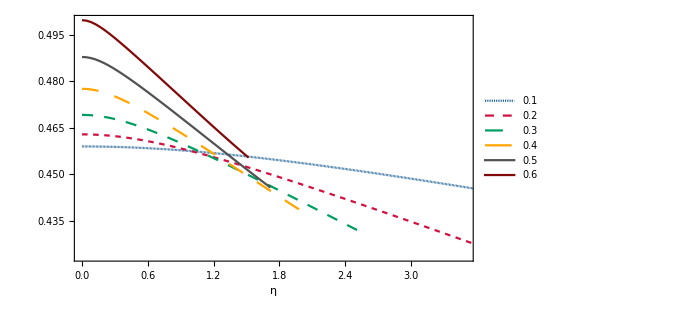

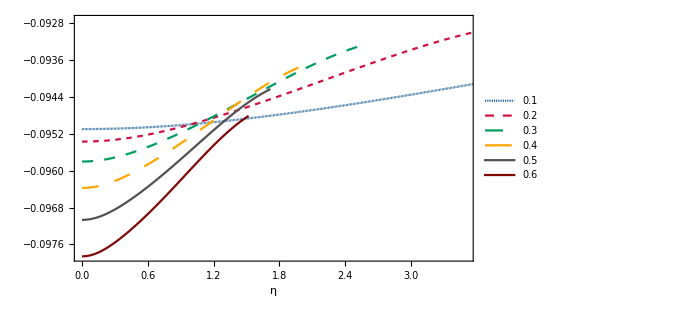

```mathematica
ListLinePlot[{Re[Tp[[1]]],Re[Tp[[2]]],Re[Tp[[3]]],Re[Tp[[4]]],Re[Tp[[5]]],Re[Tp[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[Tp[[1]]],Im[Tp[[2]]],Im[Tp[[3]]],Im[Tp[[4]]],Im[Tp[[5]]],Im[Tp[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100
(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100
(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100
(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100
```

9.73479

-2.48477

8.45765

-2.92498

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tdp]-Im[Tda])[[k]][[j+1]][[1]]/(Abs[Im[Tda][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

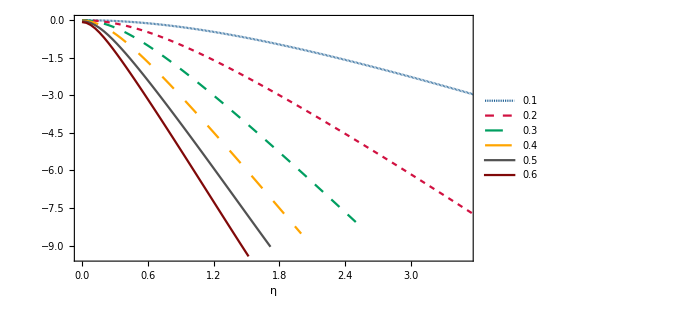

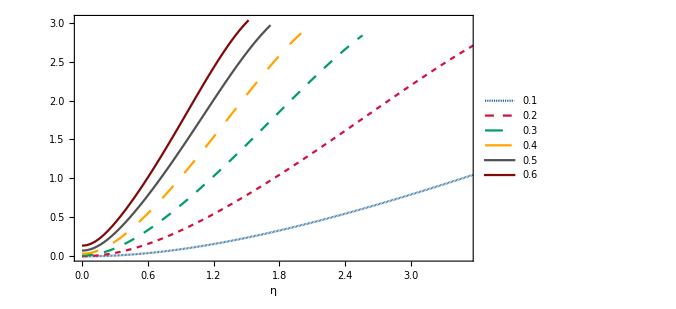

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.12,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.12,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
Max[Abs[(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100],Abs[(Max[Re[Tda[[2]]]]-Min[Re[Tda[[2]]]])/Min[Re[Tda[[2]]]]*100],Abs[(Max[Re[Tda[[3]]]]-Min[Re[Tda[[3]]]])/Min[Re[Tda[[3]]]]*100],Abs[(Max[Re[Tda[[4]]]]-Min[Re[Tda[[4]]]])/Min[Re[Tda[[4]]]]*100],Abs[(Max[Re[Tda[[5]]]]-Min[Re[Tda[[5]]]])/Min[Re[Tda[[5]]]]*100],Abs[(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100]]
Max[Abs[(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100],Abs[(Max[Im[Tda[[2]]]]-Min[Im[Tda[[2]]]])/Min[Im[Tda[[2]]]]*100],Abs[(Max[Im[Tda[[3]]]]-Min[Im[Tda[[3]]]])/Min[Im[Tda[[3]]]]*100],Abs[(Max[Im[Tda[[4]]]]-Min[Im[Tda[[4]]]])/Min[Im[Tda[[4]]]]*100],Abs[(Max[Im[Tda[[5]]]]-Min[Im[Tda[[5]]]])/Min[Im[Tda[[5]]]]*100],Abs[(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100]]
```

0.54356

0.27365

```mathematica
Max[Abs[(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100],Abs[(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100],Abs[(Max[Re[Tdp[[3]]]]-Min[Re[Tdp[[3]]]])/Min[Re[Tdp[[3]]]]*100],Abs[(Max[Re[Tdp[[4]]]]-Min[Re[Tdp[[4]]]])/Min[Re[Tdp[[4]]]]*100],Abs[(Max[Re[Tdp[[5]]]]-Min[Re[Tdp[[5]]]])/Min[Re[Tdp[[5]]]]*100],Abs[(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100],Abs[(Max[Im[Tdp[[2]]]]-Min[Im[Tdp[[2]]]])/Min[Im[Tdp[[2]]]]*100],Abs[(Max[Im[Tdp[[3]]]]-Min[Im[Tdp[[3]]]])/Min[Im[Tdp[[3]]]]*100],Abs[(Max[Im[Tdp[[4]]]]-Min[Im[Tdp[[4]]]])/Min[Im[Tdp[[4]]]]*100],Abs[(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100],Abs[(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100]]
```

9.73479

3.11427

## l=0,1,2 Scalar mode polar

#### L=0

```mathematica
Ts0={{{0,0.11064799455968062-0.10493815338417739 ⅈ},{1/25+ⅈ/25,0.1106486124867129-0.10493828765864432 ⅈ},{2/25+(2 ⅈ)/25,0.11065046626243158-0.10493869048168607 ⅈ},{3/25+(3 ⅈ)/25,0.11065355586452665-0.1049393618508811 ⅈ},{4/25+(4 ⅈ)/25,0.11065788125685697-0.10494030176241265 ⅈ},{1/5+ⅈ/5,0.11066344238885042-0.10494151021092722 ⅈ},{6/25+(6 ⅈ)/25,0.11067023919552992-0.10494298718952481 ⅈ},{7/25+(7 ⅈ)/25,0.11067827159754598-0.10494473268974586 ⅈ},{8/25+(8 ⅈ)/25,0.1106875395012173-0.10494674670155572 ⅈ},{9/25+(9 ⅈ)/25,0.1106980427985781-0.10494902921332613 ⅈ},{2/5+(2 ⅈ)/5,0.11070978136743301-0.10495158021181365 ⅈ},{11/25+(11 ⅈ)/25,0.11072275507141907-0.10495439968213537 ⅈ},{12/25+(12 ⅈ)/25,0.1107369637600749-0.10495748760774164 ⅈ},{13/25+(13 ⅈ)/25,0.11075240726891716-0.10496084397038584 ⅈ},{14/25+(14 ⅈ)/25,0.1107690854195241-0.10496446875009124 ⅈ},{3/5+(3 ⅈ)/5,0.11078699801962612-0.10496836192511476 ⅈ},{16/25+(16 ⅈ)/25,0.11080614486320353-0.10497252347190794 ⅈ},{17/25+(17 ⅈ)/25,0.11082652573059125-0.10497695336507461 ⅈ},{18/25+(18 ⅈ)/25,0.11084814038859045-0.1049816515773257 ⅈ},{19/25+(19 ⅈ)/25,0.11087098859058726-0.10498661807943092 ⅈ},{4/5+(4 ⅈ)/5,0.11089507007667815-0.1049918528401672 ⅈ},{21/25+(21 ⅈ)/25,0.11092038457380211-0.10499735582626414 ⅈ},{22/25+(22 ⅈ)/25,0.11094693179587997-0.10500312700234608 ⅈ},{23/25+(23 ⅈ)/25,0.11097471144395972-0.10500916633087122 ⅈ},{24/25+(24 ⅈ)/25,0.11100372320636916-0.1050154737720671 ⅈ},{1+ⅈ,0.11103396675887463-0.10502204928386315 ⅈ},{26/25+(26 ⅈ)/25,0.11106544176484612-0.10502889282181978 ⅈ},{27/25+(27 ⅈ)/25,0.11109814787543006-0.10503600433905297 ⅈ},{28/25+(28 ⅈ)/25,0.11113208472972552-0.10504338378615867 ⅈ},{29/25+(29 ⅈ)/25,0.1111672519549702-0.10505103111112928 ⅈ},{6/5+(6 ⅈ)/5,0.11120364916673016-0.10505894625926983 ⅈ},{31/25+(31 ⅈ)/25,0.11124127596909646-0.10506712917310944 ⅈ},{32/25+(32 ⅈ)/25,0.11128013195488752-0.1050755797923092 ⅈ},{33/25+(33 ⅈ)/25,0.11132021670585766-0.1050842980535664 ⅈ},{34/25+(34 ⅈ)/25,0.1113615297929111-0.10509328389051499 ⅈ},{7/5+(7 ⅈ)/5,0.11140407077632182-0.10510253723362233 ⅈ},{36/25+(36 ⅈ)/25,0.1114478392059589-0.10511205801008193 ⅈ},{37/25+(37 ⅈ)/25,0.11149283462151738-0.10512184614370243 ⅈ},{38/25+(38 ⅈ)/25,0.11153905655275441-0.10513190155479256 ⅈ},{39/25+(39 ⅈ)/25,0.11158650451973066-0.1051422241600418 ⅈ},{8/5+(8 ⅈ)/5,0.11163517803305689-0.10515281387239739 ⅈ},{41/25+(41 ⅈ)/25,0.11168507659414541-0.10516367060093687 ⅈ},{42/25+(42 ⅈ)/25,0.11173619969546653-0.10517479425073642 ⅈ},{43/25+(43 ⅈ)/25,0.11178854682080962-0.10518618472273489 ⅈ},{44/25+(44 ⅈ)/25,0.11184211744554895-0.10519784191359366 ⅈ},{9/5+(9 ⅈ)/5,0.11189691103691374-0.1052097657155518 ⅈ},{46/25+(46 ⅈ)/25,0.11195292705426299-0.10522195601627678 ⅈ},{47/25+(47 ⅈ)/25,0.11201016494936399-0.10523441269871092 ⅈ},{48/25+(48 ⅈ)/25,0.11206862416667523-0.10524713564091259 ⅈ},{49/25+(49 ⅈ)/25,0.11212830414363324-0.10526012471589334 ⅈ},{2+2 ⅈ,0.11218920431094281-0.10527337979144996 ⅈ},{51/25+(51 ⅈ)/25,0.11225132409287142-0.10528690072999133 ⅈ},{52/25+(52 ⅈ)/25,0.1123146629075465-0.1053006873883612 ⅈ},{53/25+(53 ⅈ)/25,0.11237922016725634-0.10531473961765497 ⅈ},{54/25+(54 ⅈ)/25,0.11244499527875432-0.10532905726303225 ⅈ},{11/5+(11 ⅈ)/5,0.1125119876435654-0.10534364016352353 ⅈ},{56/25+(56 ⅈ)/25,0.11258019665829612-0.10535848815183245 ⅈ},{57/25+(57 ⅈ)/25,0.11264962171494687-0.10537360105413172 ⅈ},{58/25+(58 ⅈ)/25,0.11272026220122673-0.10538897868985467 ⅈ},{59/25+(59 ⅈ)/25,0.11279211750087029-0.1054046208714808 ⅈ},{12/5+(12 ⅈ)/5,0.11286518699395717-0.10542052740431591 ⅈ},{61/25+(61 ⅈ)/25,0.11293947005723265-0.10543669808626648 ⅈ},{62/25+(62 ⅈ)/25,0.11301496606443058-0.10545313270760878 ⅈ},{63/25+(63 ⅈ)/25,0.11309167438659777-0.10546983105075183 ⅈ},{64/25+(64 ⅈ)/25,0.11316959439241933-0.10548679288999462 ⅈ},{13/5+(13 ⅈ)/5,0.11324872544854525-0.10550401799127755 ⅈ},{66/25+(66 ⅈ)/25,0.11332906691991479-0.10552150611192732 ⅈ},{67/25+(67 ⅈ)/25,0.1134106181700987-0.10553925700039832 ⅈ},{68/25+(68 ⅈ)/25,0.11349337856160707-0.10555727039600285 ⅈ},{69/25+(69 ⅈ)/25,0.11357734745623232-0.10557554602864003 ⅈ},{14/5+(14 ⅈ)/5,0.1136625242153749-0.10559408361851615 ⅈ},{71/25+(71 ⅈ)/25,0.11374890820037223-0.10561288287585915 ⅈ},{72/25+(72 ⅈ)/25,0.11383649877282762-0.1056319435006267 ⅈ},{73/25+(73 ⅈ)/25,0.113925295294938-0.10565126518220752 ⅈ},{74/25+(74 ⅈ)/25,0.11401529712982142-0.10567084759911681 ⅈ},{3+3 ⅈ,0.11410650364184302-0.1056906904186843 ⅈ},{76/25+(76 ⅈ)/25,0.11419891419694005-0.1057107932967364 ⅈ},{77/25+(77 ⅈ)/25,0.11429252816294501-0.1057311558772709 ⅈ},{78/25+(78 ⅈ)/25,0.11438734490990743-0.1057517777921256 ⅈ},{79/25+(79 ⅈ)/25,0.11448336381041317-0.10577265866063952 ⅈ},{16/5+(16 ⅈ)/5,0.11458058423990185-0.10579379808930751 ⅈ},{81/25+(81 ⅈ)/25,0.11467900557698121-0.1058151956714279 ⅈ},{82/25+(82 ⅈ)/25,0.11477862720373952-0.10583685098674311 ⅈ},{83/25+(83 ⅈ)/25,0.11487944850605386-0.1058587636010731 ⅈ},{84/25+(84 ⅈ)/25,0.11498146887389599-0.105880933065942 ⅈ},{17/5+(17 ⅈ)/5,0.11508468770163414-0.10590335891819734 ⅈ},{86/25+(86 ⅈ)/25,0.11518910438833113-0.10592604067962222 ⅈ},{87/25+(87 ⅈ)/25,0.11529471833803807-0.10594897785654038 ⅈ},{88/25+(88 ⅈ)/25,0.11540152896008407-0.10597216993941373 ⅈ},{89/25+(89 ⅈ)/25,0.11550953566936087-0.1059956164024329 ⅈ},{18/5+(18 ⅈ)/5,0.11561873788660257-0.10601931670310041 ⅈ},{91/25+(91 ⅈ)/25,0.11572913503866021-0.1060432702818063 ⅈ},{92/25+(92 ⅈ)/25,0.11584072655877062-0.1060674765613969 ⅈ},{93/25+(93 ⅈ)/25,0.11595351188681928-0.10609193494673558 ⅈ},{94/25+(94 ⅈ)/25,0.11606749046959733-0.1061166448242568 ⅈ},{19/5+(19 ⅈ)/5,0.11618266176105174-0.10614160556151238 ⅈ},{96/25+(96 ⅈ)/25,0.11629902522252894-0.10616681650671038 ⅈ},{97/25+(97 ⅈ)/25,0.11641658032301101-0.10619227698824688 ⅈ},{98/25+(98 ⅈ)/25,0.11653532653934486-0.10621798631423028 ⅈ},{99/25+(99 ⅈ)/25,0.11665526335646323-0.106243943771998 ⅈ},{4+4 ⅈ,0.11677639026759794-0.10627014862762638 ⅈ},{101/25+(101 ⅈ)/25,0.11689870677448451-0.10629660012543271 ⅈ},{102/25+(102 ⅈ)/25,0.11702221238755818-0.10632329748747038 ⅈ},{103/25+(103 ⅈ)/25,0.11714690662614066-0.10635023991301676 ⅈ},{104/25+(104 ⅈ)/25,0.11727278901861775-0.10637742657805355 ⅈ},{21/5+(21 ⅈ)/5,0.117399859102607-0.10640485663474063 ⅈ},{106/25+(106 ⅈ)/25,0.11752811642511521-0.10643252921088213 ⅈ},{107/25+(107 ⅈ)/25,0.11765756054268574-0.10646044340938607 ⅈ},{108/25+(108 ⅈ)/25,0.11778819102153472-0.10648859830771656 ⅈ},{109/25+(109 ⅈ)/25,0.11792000743767644-0.10651699295733977 ⅈ},{22/5+(22 ⅈ)/5,0.11805300937703679-0.1065456263831624 ⅈ},{111/25+(111 ⅈ)/25,0.11818719643555524-0.10657449758296406 ⅈ},{112/25+(112 ⅈ)/25,0.1183225682192743-0.10660360552682285 ⅈ},{113/25+(113 ⅈ)/25,0.11845912434441663-0.10663294915653451 ⅈ},{114/25+(114 ⅈ)/25,0.11859686443744895-0.1066625273850252 ⅈ},{23/5+(23 ⅈ)/5,0.11873578813513261-0.10669233909575829 ⅈ},{116/25+(116 ⅈ)/25,0.11887589508456077-0.10672238314213482 ⅈ},{117/25+(117 ⅈ)/25,0.1190171849431811-0.10675265834688825 ⅈ},{118/25+(118 ⅈ)/25,0.11915965737880414-0.10678316350147353 ⅈ},{119/25+(119 ⅈ)/25,0.11930331206959703-0.10681389736545041 ⅈ},{24/5+(24 ⅈ)/5,0.11944814870406172-0.10684485866586156 ⅈ},{121/25+(121 ⅈ)/25,0.11959416698099772-0.10687604609660546 ⅈ},{122/25+(122 ⅈ)/25,0.11974136660944884-0.10690745831780422 ⅈ},{123/25+(123 ⅈ)/25,0.1198897473086338-0.10693909395516699 ⅈ},{124/25+(124 ⅈ)/25,0.12003930880785942-0.10697095159934832 ⅈ},{5+5 ⅈ,0.12019005084641761-0.10700302980530277 ⅈ},{126/25+(126 ⅈ)/25,0.12034197317346415-0.10703532709163523 ⅈ},{127/25+(127 ⅈ)/25,0.1204950755478797-0.10706784193994758 ⅈ},{128/25+(128 ⅈ)/25,0.12064935773811283-0.10710057279418182 ⅈ},{129/25+(129 ⅈ)/25,0.12080481952200406-0.10713351805996016 ⅈ},{26/5+(26 ⅈ)/5,0.12096146068659104-0.10716667610392223 ⅈ},{131/25+(131 ⅈ)/25,0.12111928102789418-0.10720004525305966 ⅈ},{132/25+(132 ⅈ)/25,0.12127828035068267-0.10723362379404859 ⅈ},{133/25+(133 ⅈ)/25,0.12143845846822011-0.10726740997258044 ⅈ},{134/25+(134 ⅈ)/25,0.12159981520198981-0.1073014019926909 ⅈ},{27/5+(27 ⅈ)/5,0.1217623503813991-0.10733559801608829 ⅈ},{136/25+(136 ⅈ)/25,0.12192606384346215-0.10736999616148088 ⅈ},{137/25+(137 ⅈ)/25,0.1220909554324617-0.10740459450390427 ⅈ},{138/25+(138 ⅈ)/25,0.12225702499958828-0.1074393910740487 ⅈ},{139/25+(139 ⅈ)/25,0.12242427240255725-0.10747438385758709 ⅈ},{28/5+(28 ⅈ)/5,0.12259269750520337-0.10750957079450431 ⅈ},{141/25+(141 ⅈ)/25,0.12276230017705203-0.10754494977842792 ⅈ},{142/25+(142 ⅈ)/25,0.12293308029286754-0.10758051865596094 ⅈ},{143/25+(143 ⅈ)/25,0.12310503773217717-0.10761627522601745 ⅈ},{144/25+(144 ⅈ)/25,0.12327817237877194-0.10765221723916116 ⅈ},{29/5+(29 ⅈ)/5,0.12345248412018245-0.10768834239694772 ⅈ},{146/25+(146 ⅈ)/25,0.1236279728471306-0.10772464835127141 ⅈ},{147/25+(147 ⅈ)/25,0.12380463845295632-0.10776113270371664 ⅈ},{148/25+(148 ⅈ)/25,0.1239824808330188-0.10779779300491484 ⅈ},{149/25+(149 ⅈ)/25,0.12416149988407309-0.10783462675390766 ⅈ},{6+6 ⅈ,0.12434169550362029-0.10787163139751682 ⅈ},{151/25+(151 ⅈ)/25,0.12452306758923228-0.10790880432972128 ⅈ},{152/25+(152 ⅈ)/25,0.1247056160378502-0.10794614289104283 ⅈ},{153/25+(153 ⅈ)/25,0.1248893407450567-0.10798364436794014 ⅈ},{154/25+(154 ⅈ)/25,0.1250742416043215-0.10802130599221257 ⅈ},{31/5+(31 ⅈ)/5,0.1252603185062206-0.10805912494041423 ⅈ},{156/25+(156 ⅈ)/25,0.1254475713376283-0.1080970983332789 ⅈ},{157/25+(157 ⅈ)/25,0.12563599998088237-0.10813522323515698 ⅈ},{158/25+(158 ⅈ)/25,0.12582560431292242-0.10817349665346508 ⅈ},{159/25+(159 ⅈ)/25,0.12601638420440045-0.10821191553814861 ⅈ},{32/5+(32 ⅈ)/5,0.1262083395187648-0.10825047678115923 ⅈ},{161/25+(161 ⅈ)/25,0.12640147011131642-0.10828917721594677 ⅈ},{162/25+(162 ⅈ)/25,0.1265957758282376-0.10832801361696766 ⅈ},{163/25+(163 ⅈ)/25,0.12679125650559395-0.10836698269920976 ⅈ},{164/25+(164 ⅈ)/25,0.1269879119683085-0.1084060811177353 ⅈ},{33/5+(33 ⅈ)/5,0.1271857420291085-0.1084453054672421 ⅈ},{166/25+(166 ⅈ)/25,0.12738474648744563-0.10848465228164478 ⅈ},{167/25+(167 ⅈ)/25,0.12758492512838815-0.10852411803367605 ⅈ},{168/25+(168 ⅈ)/25,0.12778627772148682-0.10856369913450996 ⅈ},{169/25+(169 ⅈ)/25,0.12798880401961368-0.10860339193340712 ⅈ},{34/5+(34 ⅈ)/5,0.12819250375777416-0.10864319271738375 ⅈ},{171/25+(171 ⅈ)/25,0.12839737665189302-0.10868309771090497 ⅈ},{172/25+(172 ⅈ)/25,0.1286034223975736-0.10872310307560366 ⅈ},{173/25+(173 ⅈ)/25,0.12881064066883216-0.10876320491002561 ⅈ},{174/25+(174 ⅈ)/25,0.12901903111680546-0.1088033992494023 ⅈ},{7+7 ⅈ,0.12922859336843442-0.10884368206545227 ⅈ},{176/25+(176 ⅈ)/25,0.12943932702512218-0.10888404926621183 ⅈ},{177/25+(177 ⅈ)/25,0.1296512316613682-0.10892449669589664 ⅈ},{178/25+(178 ⅈ)/25,0.12986430682337843-0.10896502013479492 ⅈ}},{{0,0.11122389751741922-0.10506674682006614 ⅈ},{1/25+ⅈ/25,0.11122636068518575-0.10506727011029296 ⅈ},{2/25+(2 ⅈ)/25,0.1112337500764896-0.1050688399731784 ⅈ},{3/25+(3 ⅈ)/25,0.11124606533094483-0.10507145638001773 ⅈ},{4/25+(4 ⅈ)/25,0.11126330585278996-0.10507511928355216 ⅈ},{1/5+ⅈ/5,0.11128547080958814-0.10507982861701023 ⅈ},{6/25+(6 ⅈ)/25,0.11131255913385303-0.10508558429349647 ⅈ},{7/25+(7 ⅈ)/25,0.11134456952513425-0.10509238620520284 ⅈ},{8/25+(8 ⅈ)/25,0.11138150045255872-0.10510023422244003 ⅈ},{9/25+(9 ⅈ)/25,0.11142335015782405-0.1051091281924867 ⅈ},{2/5+(2 ⅈ)/5,0.11147011665863771-0.10511906793825311 ⅈ},{11/25+(11 ⅈ)/25,0.11152179775259657-0.10513005325675587 ⅈ},{12/25+(12 ⅈ)/25,0.11157839102150026-0.10514208391739929 ⅈ},{13/25+(13 ⅈ)/25,0.1116398938360897-0.10515515966005957 ⅈ},{14/25+(14 ⅈ)/25,0.11170630336120331-0.10516928019296627 ⅈ},{3/5+(3 ⅈ)/5,0.11177761656134105-0.10518444519037638 ⅈ},{16/25+(16 ⅈ)/25,0.11185383020662254-0.10520065429003385 ⅈ},{17/25+(17 ⅈ)/25,0.11193494087915114-0.10521790709041291 ⅈ},{18/25+(18 ⅈ)/25,0.11202094497971787-0.10523620314773008 ⅈ},{19/25+(19 ⅈ)/25,0.11211183873490238-0.10525554197272773 ⅈ},{4/5+(4 ⅈ)/5,0.11220761820450774-0.10527592302721571 ⅈ},{21/25+(21 ⅈ)/25,0.11230827928933401-0.10529734572036593 ⅈ},{22/25+(22 ⅈ)/25,0.1124138177392736-0.1053198094047513 ⅈ},{23/25+(23 ⅈ)/25,0.11252422916171137-0.10534331337212167 ⅈ},{24/25+(24 ⅈ)/25,0.11263950903021486-0.10536785684890755 ⅈ},{1+ⅈ,0.11275965269349622-0.10539343899144396 ⅈ},{26/25+(26 ⅈ)/25,0.11288465538462883-0.10542005888090497 ⅈ},{27/25+(27 ⅈ)/25,0.11301451223049916-0.1054477155179404 ⅈ},{28/25+(28 ⅈ)/25,0.11314921826147538-0.10547640781700486 ⅈ},{29/25+(29 ⅈ)/25,0.11328876842127132-0.1055061346003712 ⅈ},{6/5+(6 ⅈ)/5,0.11343315757698579-0.10553689459181773 ⅈ},{31/25+(31 ⅈ)/25,0.11358238052929488-0.10556868640998053 ⅈ},{32/25+(32 ⅈ)/25,0.11373643202277471-0.10560150856136148 ⅈ},{33/25+(33 ⅈ)/25,0.11389530675633133-0.10563535943298222 ⅈ},{34/25+(34 ⅈ)/25,0.11405899939371333-0.10567023728467528 ⅈ},{7/5+(7 ⅈ)/5,0.1142275045740823-0.10570614024100261 ⅈ},{36/25+(36 ⅈ)/25,0.11440081692261536-0.10574306628279287 ⅈ},{37/25+(37 ⅈ)/25,0.1145789310611125-0.10578101323828834 ⅈ},{38/25+(38 ⅈ)/25,0.11476184161858217-0.10581997877389304 ⅈ},{39/25+(39 ⅈ)/25,0.11494954324177578-0.10585996038451327 ⅈ},{8/5+(8 ⅈ)/5,0.11514203060564229-0.10590095538348308 ⅈ},{41/25+(41 ⅈ)/25,0.1153392984236733-0.10594296089206677 ⅈ},{42/25+(42 ⅈ)/25,0.11554134145810638-0.10598597382853117 ⅈ},{43/25+(43 ⅈ)/25,0.11574815452995647-0.10602999089678145 ⅈ},{44/25+(44 ⅈ)/25,0.11595973252884123-0.10607500857455397 ⅈ},{9/5+(9 ⅈ)/5,0.11617607042256738-0.1061210231011613 ⅈ},{46/25+(46 ⅈ)/25,0.11639716326644374-0.10616803046478424 ⅈ},{47/25+(47 ⅈ)/25,0.116623006212285-0.10621602638930769 ⅈ},{48/25+(48 ⅈ)/25,0.11685359451707017-0.10626500632069677 ⅈ},{49/25+(49 ⅈ)/25,0.11708892355121876-0.10631496541291213 ⅈ},{2+2 ⅈ,0.11732898880644624-0.10636589851336263 ⅈ},{51/25+(51 ⅈ)/25,0.11757378590315991-0.10641780014789677 ⅈ},{52/25+(52 ⅈ)/25,0.11782331059735535-0.10647066450533399 ⅈ},{53/25+(53 ⅈ)/25,0.11807755878697254-0.1065244854215388 ⅈ},{54/25+(54 ⅈ)/25,0.11833652651767045-0.10657925636304283 ⅈ},{11/5+(11 ⅈ)/5,0.11860020998797699-0.10663497041022044 ⅈ},{56/25+(56 ⅈ)/25,0.11886860555377192-0.10669162024002639 ⅈ},{57/25+(57 ⅈ)/25,0.11914170973205772-0.10674919810830465 ⅈ},{58/25+(58 ⅈ)/25,0.11941951920397492-0.10680769583168119 ⅈ},{59/25+(59 ⅈ)/25,0.1197020308170153-0.1068671047690535 ⅈ},{12/5+(12 ⅈ)/5,0.11998924158638784-0.10692741580269433 ⅈ},{61/25+(61 ⅈ)/25,0.12028114869549038-0.10698861931898734 ⅈ},{62/25+(62 ⅈ)/25,0.1205777494954402-0.10705070518881638 ⅈ},{63/25+(63 ⅈ)/25,0.12087904150361621-0.1071136627476323 ⅈ},{64/25+(64 ⅈ)/25,0.12118502240116506-0.1071774807752243 ⅈ},{13/5+(13 ⅈ)/5,0.12149569002942331-0.10724214747522501 ⅈ},{66/25+(66 ⅈ)/25,0.1218110423852084-0.10730765045438345 ⅈ},{67/25+(67 ⅈ)/25,0.12213107761492983-0.10737397670164119 ⅈ},{68/25+(68 ⅈ)/25,0.12245579400747496-0.10744111256705238 ⅈ},{69/25+(69 ⅈ)/25,0.12278518998582054-0.10750904374059082 ⅈ},{14/5+(14 ⅈ)/5,0.1231192640973259-0.10757775523089134 ⅈ},{71/25+(71 ⅈ)/25,0.1234580150026613-0.10764723134397725 ⅈ},{72/25+(72 ⅈ)/25,0.1238014414633283-0.10771745566202832 ⅈ},{73/25+(73 ⅈ)/25,0.12414954232772928-0.1077884110222499 ⅈ},{74/25+(74 ⅈ)/25,0.12450231651574536-0.107860079495906 ⅈ},{3+3 ⅈ,0.1248597630017841-0.10793244236758547 ⅈ},{76/25+(76 ⅈ)/25,0.12522188079626076-0.10800548011477336 ⅈ},{77/25+(77 ⅈ)/25,0.12558866892547893-0.1080791723878051 ⅈ},{78/25+(78 ⅈ)/25,0.1259601264098806-0.10815349799028565 ⅈ},{79/25+(79 ⅈ)/25,0.12633625224063835-0.10822843486005966 ⅈ},{16/5+(16 ⅈ)/5,0.1267170453545663-0.10830396005082456 ⅈ},{81/25+(81 ⅈ)/25,0.12710250460733152-0.10838004971448187 ⅈ},{82/25+(82 ⅈ)/25,0.12749262874495146-0.10845667908432743 ⅈ},{83/25+(83 ⅈ)/25,0.12788741637356874-0.10853382245918543 ⅈ},{84/25+(84 ⅈ)/25,0.12828686592750105-0.10861145318859522 ⅈ},{17/5+(17 ⅈ)/5,0.1286909756355683-0.10868954365916435 ⅈ},{86/25+(86 ⅈ)/25,0.1290997434857084-0.10876806528220508 ⅈ},{87/25+(87 ⅈ)/25,0.12951316718789868-0.10884698848277513 ⅈ},{88/25+(88 ⅈ)/25,0.12993124413540785-0.10892628269024696 ⅈ},{89/25+(89 ⅈ)/25,0.1303539713644134-0.1090059163305321 ⅈ},{18/5+(18 ⅈ)/5,0.13078134551202597-0.1090858568200913 ⅈ},{91/25+(91 ⅈ)/25,0.13121336277277365-0.10916607056186059 ⅈ}},{{0,0.11217302716116802-0.1052851033436859 ⅈ},{1/25+ⅈ/25,0.11217853849146973-0.10528623065036542 ⅈ},{2/25+(2 ⅈ)/25,0.11219507186590848-0.10528961254848608 ⅈ},{3/25+(3 ⅈ)/25,0.11222262538259221-0.10529524896010085 ⅈ},{4/25+(4 ⅈ)/25,0.11226119588961299-0.10530313975410546 ⅈ},{1/5+ⅈ/5,0.11231077899259076-0.10531328474048299 ⅈ},{6/25+(6 ⅈ)/25,0.11237136907288126-0.10532568366378503 ⅈ},{7/25+(7 ⅈ)/25,0.11244295931086369-0.10534033619467927 ⅈ},{8/25+(8 ⅈ)/25,0.11252554171424126-0.10535724191951695 ⅈ},{9/25+(9 ⅈ)/25,0.11261910715119612-0.10537640032785156 ⅈ},{2/5+(2 ⅈ)/5,0.11272364538833249-0.10539781079784055 ⅈ},{11/25+(11 ⅈ)/25,0.11283914513321845-0.10542147257944558 ⅈ},{12/25+(12 ⅈ)/25,0.11296559408137602-0.10544738477533837 ⅈ},{13/25+(13 ⅈ)/25,0.1131029789675317-0.10547554631941017 ⅈ},{14/25+(14 ⅈ)/25,0.11325128562092394-0.1055059559527744 ⅈ},{3/5+(3 ⅈ)/5,0.11341049902444383-0.1055386121971436 ⅈ},{16/25+(16 ⅈ)/25,0.11358060337736814-0.10557351332545427 ⅈ},{17/25+(17 ⅈ)/25,0.11376158216142421-0.10561065732960707 ⅈ},{18/25+(18 ⅈ)/25,0.1139534182099082-0.10565004188518347 ⅈ},{19/25+(19 ⅈ)/25,0.11415609377955978-0.10569166431299515 ⅈ},{4/5+(4 ⅈ)/5,0.11436959062487702-0.10573552153731873 ⅈ},{21/25+(21 ⅈ)/25,0.11459389007453857-0.10578161004066439 ⅈ},{22/25+(22 ⅈ)/25,0.11482897310957953-0.1058299258149265 ⅈ},{23/25+(23 ⅈ)/25,0.11507482044295068-0.10588046430876202 ⅈ},{24/25+(24 ⅈ)/25,0.1153314126000706-0.10593322037104427 ⅈ},{1+ⅈ,0.11559872999996242-0.10598818819024085 ⅈ},{26/25+(26 ⅈ)/25,0.11587675303654685-0.10604536122956794 ⅈ},{27/25+(27 ⅈ)/25,0.11616546215964238-0.10610473215777981 ⅈ},{28/25+(28 ⅈ)/25,0.1164648379552123-0.10616629277545422 ⅈ},{29/25+(29 ⅈ)/25,0.11677486122435962-0.10623003393665266 ⅈ},{6/5+(6 ⅈ)/5,0.11709551306057454-0.10629594546583371 ⅈ},{31/25+(31 ⅈ)/25,0.11742677492469934-0.10636401606991981 ⅈ},{32/25+(32 ⅈ)/25,0.1177686287170638-0.106434233245429 ⅈ},{33/25+(33 ⅈ)/25,0.11812105684622119-0.10650658318060295 ⅈ},{34/25+(34 ⅈ)/25,0.1184840422936936-0.10658105065248306 ⅈ},{7/5+(7 ⅈ)/5,0.11885756867411315-0.10665761891891085 ⅈ},{36/25+(36 ⅈ)/25,0.11924162029012617-0.10673626960545717 ⅈ},{37/25+(37 ⅈ)/25,0.11963618218140407-0.10681698258731513 ⅈ},{38/25+(38 ⅈ)/25,0.1200412401670861-0.10689973586622739 ⅈ},{39/25+(39 ⅈ)/25,0.12045678088095786-0.106984505442558 ⅈ},{8/5+(8 ⅈ)/5,0.12088279179865102-0.10707126518266222 ⅈ},{41/25+(41 ⅈ)/25,0.12131926125613245-0.10715998668175734 ⅈ},{42/25+(42 ⅈ)/25,0.1217661784587352-0.10725063912254983 ⅈ},{43/25+(43 ⅈ)/25,0.12222353347996981-0.10734318912993396 ⅈ},{44/25+(44 ⅈ)/25,0.12269131724934607-0.10743760062214047 ⅈ},{9/5+(9 ⅈ)/5,0.12316952152842586-0.10753383465878402 ⅈ},{46/25+(46 ⅈ)/25,0.12365813887432872-0.10763184928633317 ⅈ},{47/25+(47 ⅈ)/25,0.12415716258991126-0.10773159938160776 ⅈ},{48/25+(48 ⅈ)/25,0.12466658665985356-0.10783303649399568 ⅈ},{49/25+(49 ⅈ)/25,0.12518640567189976-0.10793610868717249 ⅈ},{2+2 ⅈ,0.12571661472252507-0.10804076038120558 ⅈ},{51/25+(51 ⅈ)/25,0.12625720930633502-0.10814693219602622 ⅈ},{52/25+(52 ⅈ)/25,0.12680818518854586-0.10825456079736039 ⅈ},{53/25+(53 ⅈ)/25,0.12736953825995176-0.10836357874631827 ⅈ},{54/25+(54 ⅈ)/25,0.1279412643738515-0.10847391435395665 ⅈ},{11/5+(11 ⅈ)/5,0.1285233591644916-0.10858549154224141 ⅈ},{56/25+(56 ⅈ)/25,0.12911581784667836-0.10869822971295266 ⅈ},{57/25+(57 ⅈ)/25,0.1297186349963282-0.10881204362618847 ⅈ},{58/25+(58 ⅈ)/25,0.1303318043118558-0.10892684329023118 ⅈ},{59/25+(59 ⅈ)/25,0.13095531835644939-0.10904253386464648 ⅈ},{12/5+(12 ⅈ)/5,0.13158916828145434-0.10915901557857974 ⅈ},{61/25+(61 ⅈ)/25,0.13223334353127156-0.10927618366630032 ⅈ},{62/25+(62 ⅈ)/25,0.13288783153038847-0.10939392832211606 ⅈ},{63/25+(63 ⅈ)/25,0.1335526173533868-0.10951213467683532 ⅈ},{64/25+(64 ⅈ)/25,0.1342276833790187-0.10963068279798756 ⅈ}},{{0,0.11347990895500862-0.10559846113417 ⅈ},{1/25+ⅈ/25,0.11348963438209472-0.10560034653518746 ⅈ},{2/25+(2 ⅈ)/25,0.11351880857994864-0.10560600275171923 ⅈ},{3/25+(3 ⅈ)/25,0.11356742521554324-0.10561542980064048 ⅈ},{4/25+(4 ⅈ)/25,0.11363547379808474-0.10562862769747182 ⅈ},{1/5+ⅈ/5,0.11372293974104623-0.10564559643069173 ⅈ},{6/25+(6 ⅈ)/25,0.1138298044619445-0.10566633592804942 ⅈ},{7/25+(7 ⅈ)/25,0.11395604550954323-0.10569084601262989 ⅈ},{8/25+(8 ⅈ)/25,0.11410163671761588-0.10571912634821558 ⅈ},{9/25+(9 ⅈ)/25,0.11426654838427207-0.10575117637339179 ⅈ},{2/5+(2 ⅈ)/5,0.11445074747565802-0.10578699522375494 ⅈ},{11/25+(11 ⅈ)/25,0.11465419785266898-0.10582658164150044 ⅈ},{12/25+(12 ⅈ)/25,0.114876860519139-0.10586993387159027 ⅈ},{13/25+(13 ⅈ)/25,0.11511869388980354-0.10591704954363136 ⅈ},{14/25+(14 ⅈ)/25,0.11537965407616242-0.10596792553853528 ⅈ},{3/5+(3 ⅈ)/5,0.11565969518820565-0.10602255783897868 ⅈ},{16/25+(16 ⅈ)/25,0.11595876964980026-0.10608094136264283 ⅈ},{17/25+(17 ⅈ)/25,0.11627682852537251-0.10614306977717974 ⅈ},{18/25+(18 ⅈ)/25,0.11661382185535839-0.10620893529583696 ⅈ},{19/25+(19 ⅈ)/25,0.1169696989977302-0.10627852845266707 ⅈ},{4/5+(4 ⅈ)/5,0.11734440897274401-0.10635183785626116 ⅈ},{21/25+(21 ⅈ)/25,0.11773790080788478-0.10642884992097258 ⅈ},{22/25+(22 ⅈ)/25,0.11815012387981767-0.10650954857464476 ⅈ},{23/25+(23 ⅈ)/25,0.11858102824997938-0.10659391494192497 ⅈ},{24/25+(24 ⅈ)/25,0.11903056499026851-0.10668192700233613 ⅈ},{1+ⅈ,0.11949868649511086-0.10677355922239651 ⅈ},{26/25+(26 ⅈ)/25,0.11998534677599339-0.1068687821612248 ⅈ},{27/25+(27 ⅈ)/25,0.1204905017343577-0.10696756204923911 ⅈ},{28/25+(28 ⅈ)/25,0.1210141094086006-0.10706986033979768 ⅈ},{29/25+(29 ⅈ)/25,0.12155613019064235-0.10717563323383905 ⅈ},{6/5+(6 ⅈ)/5,0.1221165270074529-0.10728483117793616 ⅈ},{31/25+(31 ⅈ)/25,0.12269526546264733-0.10739739833648299 ⅈ},{32/25+(32 ⅈ)/25,0.12329231393313551-0.10751327203915909 ⅈ},{33/25+(33 ⅈ)/25,0.12390764361564084-0.10763238220527138 ⅈ},{34/25+(34 ⅈ)/25,0.12454122851777116-0.10775465074709768 ⅈ},{7/5+(7 ⅈ)/5,0.12519304538822473-0.10787999095494606 ⅈ},{36/25+(36 ⅈ)/25,0.1258630735806567-0.1080083068673039 ⅈ},{37/25+(37 ⅈ)/25,0.1265512948457308-0.10813949263017918 ⅈ},{38/25+(38 ⅈ)/25,0.1272576930459499-0.10827343185053871 ⅈ},{39/25+(39 ⅈ)/25,0.12798225378801345-0.1084099969496176 ⅈ},{8/5+(8 ⅈ)/5,0.1287249639677075-0.10854904852281047 ⅈ},{41/25+(41 ⅈ)/25,0.12948581122271544-0.10869043471384836 ⅈ},{42/25+(42 ⅈ)/25,0.13026478328925856-0.10883399061200665 ⅈ},{43/25+(43 ⅈ)/25,0.1310618672591635-0.10897953768216137 ⅈ},{44/25+(44 ⅈ)/25,0.13187704873482264-0.10912688323859722 ⅈ},{9/5+(9 ⅈ)/5,0.13271031088058738-0.10927581997454217 ⅈ},{46/25+(46 ⅈ)/25,0.13356163337042734-0.10942612556043031 ⅈ},{47/25+(47 ⅈ)/25,0.13443099123322003-0.10957756232484266 ⅈ},{48/25+(48 ⅈ)/25,0.1353183535988064-0.10972987703289634 ⅈ},{49/25+(49 ⅈ)/25,0.1362236823499727-0.10988280077750229 ⅈ},{2+2 ⅈ,0.13714693068778328-0.1100360489993325 ⅈ}},{{0,0.11512402986066302-0.10601270587756181 ⅈ},{1/25+ⅈ/25,0.11513908992426376-0.10601542832496033 ⅈ},{2/25+(2 ⅈ)/25,0.11518426470543387-0.10602359593512235 ⅈ},{3/25+(3 ⅈ)/25,0.11525953787829632-0.10603720946854345 ⅈ},{4/25+(4 ⅈ)/25,0.11536488243644319-0.10605627014306307 ⅈ},{1/5+ⅈ/5,0.11550026094344036-0.10608077954890255 ⅈ},{6/25+(6 ⅈ)/25,0.11566562590106265-0.10611073953163713 ⅈ},{7/25+(7 ⅈ)/25,0.1158609202165617-0.10614615203851888 ⅈ},{8/25+(8 ⅈ)/25,0.11608607776441553-0.10618701892579598 ⅈ},{9/25+(9 ⅈ)/25,0.11634102403702085-0.10623334172421779 ⅈ},{2/5+(2 ⅈ)/5,0.11662567687785111-0.10628512135949064 ⅈ},{11/25+(11 ⅈ)/25,0.11693994728969008-0.10634235782407202 ⅈ},{12/25+(12 ⅈ)/25,0.11728374030966243-0.10640504979636006 ⅈ},{13/25+(13 ⅈ)/25,0.11765695594191991-0.10647319420306262 ⅈ},{14/25+(14 ⅈ)/25,0.11805949013799803-0.10654678572031734 ⅈ},{3/5+(3 ⅈ)/5,0.11849123581402955-0.1066258162089928 ⅈ},{16/25+(16 ⅈ)/25,0.11895208389318232-0.1067102740795364 ⅈ},{17/25+(17 ⅈ)/25,0.11944192436086899-0.10680014358175705 ⅈ},{18/25+(18 ⅈ)/25,0.11996064731945152-0.10689540401505365 ⅈ},{19/25+(19 ⅈ)/25,0.12050814402832145-0.10699602885483446 ⅈ},{4/5+(4 ⅈ)/5,0.1210843079143734-0.1071019847912372 ⅈ},{21/25+(21 ⅈ)/25,0.12168903553699632-0.10721323067677208 ⅈ},{22/25+(22 ⅈ)/25,0.12232222749078323-0.10732971638019546 ⅈ},{23/25+(23 ⅈ)/25,0.12298378922820208-0.10745138154480488 ⅈ},{24/25+(24 ⅈ)/25,0.1236736317834896-0.10757815425045916 ⅈ},{1+ⅈ,0.12439167237803034-0.10770994958000159 ⅈ},{26/25+(26 ⅈ)/25,0.1251378348864934-0.10784666809243904 ⅈ},{27/25+(27 ⅈ)/25,0.12591205014204415-0.1079881942072424 ⅈ},{28/25+(28 ⅈ)/25,0.12671425605807288-0.10813439450652255 ⅈ},{29/25+(29 ⅈ)/25,0.1275443975431436-0.10828511596464224 ⅈ},{6/5+(6 ⅈ)/5,0.12840242618533776-0.10844018411807635 ⅈ},{31/25+(31 ⅈ)/25,0.12928829968193595-0.10859940119206324 ⅈ},{32/25+(32 ⅈ)/25,0.13020198099056288-0.10876254420480569 ⅈ},{33/25+(33 ⅈ)/25,0.13114343717863483-0.10892936307468278 ⅈ},{34/25+(34 ⅈ)/25,0.1321126379493496-0.10909957876109347 ⅈ},{7/5+(7 ⅈ)/5,0.13310955382470205-0.10927288147511106 ⅈ},{36/25+(36 ⅈ)/25,0.13413415396927117-0.10944892900198788 ⅈ},{37/25+(37 ⅈ)/25,0.1351864036429805-0.10962734518356947 ⅈ},{38/25+(38 ⅈ)/25,0.13626626127686145-0.1098077186146569 ⅈ},{39/25+(39 ⅈ)/25,0.1373736751731972-0.10998960161304244 ⅈ},{8/5+(8 ⅈ)/5,0.13850857984042134-0.11017250952801246 ⅈ},{41/25+(41 ⅈ)/25,0.13967089198385407-0.11035592045617972 ⅈ},{42/25+(42 ⅈ)/25,0.1408605061857795-0.11053927543613182 ⅈ},{43/25+(43 ⅈ)/25,0.1420772903223911-0.11072197919406573 ⅈ}},{{0,0.11708091346793689-0.10653328692081519 ⅈ},{1/25+ⅈ/25,0.11710237876010259-0.10653684402221397 ⅈ},{2/25+(2 ⅈ)/25,0.1171667627846972-0.10654751639846907 ⅈ},{3/25+(3 ⅈ)/25,0.117274029926121-0.10656530718669607 ⅈ},{4/25+(4 ⅈ)/25,0.11742412137457098-0.10659022147541518 ⅈ},{1/5+ⅈ/5,0.11761695586800458-0.10662226607863709 ⅈ},{6/25+(6 ⅈ)/25,0.11785243074657019-0.10666144921773418 ⅈ},{7/25+(7 ⅈ)/25,0.11813042328386637-0.1067077801008515 ⅈ},{8/25+(8 ⅈ)/25,0.11845079227703863-0.1067612683914736 ⅈ},{9/25+(9 ⅈ)/25,0.11881337987407403-0.10682192355621148 ⅈ},{2/5+(2 ⅈ)/5,0.11921801361318247-0.10688975408050287 ⅈ},{11/25+(11 ⅈ)/25,0.11966450864585314-0.1069647665397541 ⅈ},{12/25+(12 ⅈ)/25,0.12015267011204535-0.10704696451251756 ⅈ},{13/25+(13 ⅈ)/25,0.12068229563298066-0.10713634732162615 ⅈ},{14/25+(14 ⅈ)/25,0.12125317788412451-0.10723290858882684 ⅈ},{3/5+(3 ⅈ)/5,0.12186510720812621-0.107336634588406 ⅈ},{16/25+(16 ⅈ)/25,0.12251787422468313-0.1074475023856319 ⅈ},{17/25+(17 ⅈ)/25,0.12321127239144719-0.10756547774661575 ⅈ},{18/25+(18 ⅈ)/25,0.12394510046715031-0.10769051280748919 ⅈ},{19/25+(19 ⅈ)/25,0.12471916482504102-0.10782254349271667 ⅈ},{4/5+(4 ⅈ)/5,0.12553328156146842-0.10796148667502396 ⅈ},{21/25+(21 ⅈ)/25,0.12638727834101446-0.10810723707297858 ⅈ},{22/25+(22 ⅈ)/25,0.12728099591598663-0.10825966388687464 ⅈ},{23/25+(23 ⅈ)/25,0.1282142892544192-0.10841860717944865 ⅈ},{24/25+(24 ⅈ)/25,0.12918702820712197-0.10858387401529618 ⅈ},{1+ⅈ,0.1301990976409735-0.10875523438189372 ⅈ},{26/25+(26 ⅈ)/25,0.13125039696288002-0.10893241692607399 ⅈ},{27/25+(27 ⅈ)/25,0.13234083895701376-0.10911510455284495 ⅈ},{28/25+(28 ⅈ)/25,0.13347034785762982-0.10930292994872551 ⅈ},{29/25+(29 ⅈ)/25,0.13463885658157623-0.10949547110934628 ⅈ},{6/5+(6 ⅈ)/5,0.13584630304933523-0.10969224697084798 ⅈ},{31/25+(31 ⅈ)/25,0.13709262553193338-0.1098927132663428 ⅈ},{32/25+(32 ⅈ)/25,0.13837775697430682-0.11009625875187629 ⅈ},{33/25+(33 ⅈ)/25,0.13970161826469313-0.11030220197012733 ⅈ},{34/25+(34 ⅈ)/25,0.14106411044530454-0.11050978874334208 ⅈ},{7/5+(7 ⅈ)/5,0.14246510589272215-0.11071819060813698 ⅈ},{36/25+(36 ⅈ)/25,0.14390443853767215-0.1109265044218182 ⅈ},{37/25+(37 ⅈ)/25,0.14538189324318346-0.11113375338034237 ⅈ},{38/25+(38 ⅈ)/25,0.14689719451705818-0.11133888968921972 ⅈ}}};
```

```mathematica
Tsd0={{{0.11064799455968062-0.10493815338417739 ⅈ},{0.1106486124867129-0.10493828765864432 ⅈ},{0.11065046626243158-0.10493869048168607 ⅈ},{0.11065355586452665-0.1049393618508811 ⅈ},{0.11065788125685697-0.10494030176241265 ⅈ},{0.11066344238885042-0.10494151021092722 ⅈ},{0.11067023919552992-0.10494298718952481 ⅈ},{0.11067827159754598-0.10494473268974586 ⅈ},{0.1106875395012173-0.10494674670155572 ⅈ},{0.1106980427985781-0.10494902921332613 ⅈ},{0.11070978136743301-0.10495158021181365 ⅈ},{0.11072275507141907-0.10495439968213537 ⅈ},{0.1107369637600749-0.10495748760774164 ⅈ},{0.11075240726891716-0.10496084397038584 ⅈ},{0.1107690854195241-0.10496446875009124 ⅈ},{0.11078699801962612-0.10496836192511476 ⅈ},{0.11080614486320353-0.10497252347190794 ⅈ},{0.11082652573059125-0.10497695336507461 ⅈ},{0.11084814038859045-0.1049816515773257 ⅈ},{0.11087098859058726-0.10498661807943092 ⅈ},{0.11089507007667815-0.1049918528401672 ⅈ},{0.11092038457380211-0.10499735582626414 ⅈ},{0.11094693179587997-0.10500312700234608 ⅈ},{0.11097471144395972-0.10500916633087122 ⅈ},{0.11100372320636916-0.1050154737720671 ⅈ},{0.11103396675887463-0.10502204928386315 ⅈ},{0.11106544176484612-0.10502889282181978 ⅈ},{0.11109814787543006-0.10503600433905297 ⅈ},{0.11113208472972552-0.10504338378615867 ⅈ},{0.1111672519549702-0.10505103111112928 ⅈ},{0.11120364916673016-0.10505894625926983 ⅈ},{0.11124127596909646-0.10506712917310944 ⅈ},{0.11128013195488752-0.1050755797923092 ⅈ},{0.11132021670585766-0.1050842980535664 ⅈ},{0.1113615297929111-0.10509328389051499 ⅈ},{0.11140407077632182-0.10510253723362233 ⅈ},{0.1114478392059589-0.10511205801008193 ⅈ},{0.11149283462151738-0.10512184614370243 ⅈ},{0.11153905655275441-0.10513190155479256 ⅈ},{0.11158650451973066-0.1051422241600418 ⅈ},{0.11163517803305689-0.10515281387239739 ⅈ},{0.11168507659414541-0.10516367060093687 ⅈ},{0.11173619969546653-0.10517479425073642 ⅈ},{0.11178854682080962-0.10518618472273489 ⅈ},{0.11184211744554895-0.10519784191359366 ⅈ},{0.11189691103691374-0.1052097657155518 ⅈ},{0.11195292705426299-0.10522195601627678 ⅈ},{0.11201016494936399-0.10523441269871092 ⅈ},{0.11206862416667523-0.10524713564091259 ⅈ},{0.11212830414363324-0.10526012471589334 ⅈ},{0.11218920431094281-0.10527337979144996 ⅈ},{0.11225132409287142-0.10528690072999133 ⅈ},{0.1123146629075465-0.1053006873883612 ⅈ},{0.11237922016725634-0.10531473961765497 ⅈ},{0.11244499527875432-0.10532905726303225 ⅈ},{0.1125119876435654-0.10534364016352353 ⅈ},{0.11258019665829612-0.10535848815183245 ⅈ},{0.11264962171494687-0.10537360105413172 ⅈ},{0.11272026220122673-0.10538897868985467 ⅈ},{0.11279211750087029-0.1054046208714808 ⅈ},{0.11286518699395717-0.10542052740431591 ⅈ},{0.11293947005723265-0.10543669808626648 ⅈ},{0.11301496606443058-0.10545313270760878 ⅈ},{0.11309167438659777-0.10546983105075183 ⅈ},{0.11316959439241933-0.10548679288999462 ⅈ},{0.11324872544854525-0.10550401799127755 ⅈ},{0.11332906691991479-0.10552150611192732 ⅈ},{0.1134106181700987-0.10553925700039832 ⅈ},{0.11349337856160707-0.10555727039600285 ⅈ},{0.11357734745623232-0.10557554602864003 ⅈ},{0.1136625242153749-0.10559408361851615 ⅈ},{0.11374890820037223-0.10561288287585915 ⅈ},{0.11383649877282762-0.1056319435006267 ⅈ},{0.113925295294938-0.10565126518220752 ⅈ},{0.11401529712982142-0.10567084759911681 ⅈ},{0.11410650364184302-0.1056906904186843 ⅈ},{0.11419891419694005-0.1057107932967364 ⅈ},{0.11429252816294501-0.1057311558772709 ⅈ},{0.11438734490990743-0.1057517777921256 ⅈ},{0.11448336381041317-0.10577265866063952 ⅈ},{0.11458058423990185-0.10579379808930751 ⅈ},{0.11467900557698121-0.1058151956714279 ⅈ},{0.11477862720373952-0.10583685098674311 ⅈ},{0.11487944850605386-0.1058587636010731 ⅈ},{0.11498146887389599-0.105880933065942 ⅈ},{0.11508468770163414-0.10590335891819734 ⅈ},{0.11518910438833113-0.10592604067962222 ⅈ},{0.11529471833803807-0.10594897785654038 ⅈ},{0.11540152896008407-0.10597216993941373 ⅈ},{0.11550953566936087-0.1059956164024329 ⅈ},{0.11561873788660257-0.10601931670310041 ⅈ},{0.11572913503866021-0.1060432702818063 ⅈ},{0.11584072655877062-0.1060674765613969 ⅈ},{0.11595351188681928-0.10609193494673558 ⅈ},{0.11606749046959733-0.1061166448242568 ⅈ},{0.11618266176105174-0.10614160556151238 ⅈ},{0.11629902522252894-0.10616681650671038 ⅈ},{0.11641658032301101-0.10619227698824688 ⅈ},{0.11653532653934486-0.10621798631423028 ⅈ},{0.11665526335646323-0.106243943771998 ⅈ},{0.11677639026759794-0.10627014862762638 ⅈ},{0.11689870677448451-0.10629660012543271 ⅈ},{0.11702221238755818-0.10632329748747038 ⅈ},{0.11714690662614066-0.10635023991301676 ⅈ},{0.11727278901861775-0.10637742657805355 ⅈ},{0.117399859102607-0.10640485663474063 ⅈ},{0.11752811642511521-0.10643252921088213 ⅈ},{0.11765756054268574-0.10646044340938607 ⅈ},{0.11778819102153472-0.10648859830771656 ⅈ},{0.11792000743767644-0.10651699295733977 ⅈ},{0.11805300937703679-0.1065456263831624 ⅈ},{0.11818719643555524-0.10657449758296406 ⅈ},{0.1183225682192743-0.10660360552682285 ⅈ},{0.11845912434441663-0.10663294915653451 ⅈ},{0.11859686443744895-0.1066625273850252 ⅈ},{0.11873578813513261-0.10669233909575829 ⅈ},{0.11887589508456077-0.10672238314213482 ⅈ},{0.1190171849431811-0.10675265834688825 ⅈ},{0.11915965737880414-0.10678316350147353 ⅈ},{0.11930331206959703-0.10681389736545041 ⅈ},{0.11944814870406172-0.10684485866586156 ⅈ},{0.11959416698099772-0.10687604609660546 ⅈ},{0.11974136660944884-0.10690745831780422 ⅈ},{0.1198897473086338-0.10693909395516699 ⅈ},{0.12003930880785942-0.10697095159934832 ⅈ},{0.12019005084641761-0.10700302980530277 ⅈ},{0.12034197317346415-0.10703532709163523 ⅈ},{0.1204950755478797-0.10706784193994758 ⅈ},{0.12064935773811283-0.10710057279418182 ⅈ},{0.12080481952200406-0.10713351805996016 ⅈ},{0.12096146068659104-0.10716667610392223 ⅈ},{0.12111928102789418-0.10720004525305966 ⅈ},{0.12127828035068267-0.10723362379404859 ⅈ},{0.12143845846822011-0.10726740997258044 ⅈ},{0.12159981520198981-0.1073014019926909 ⅈ},{0.1217623503813991-0.10733559801608829 ⅈ},{0.12192606384346215-0.10736999616148088 ⅈ},{0.1220909554324617-0.10740459450390427 ⅈ},{0.12225702499958828-0.1074393910740487 ⅈ},{0.12242427240255725-0.10747438385758709 ⅈ},{0.12259269750520337-0.10750957079450431 ⅈ},{0.12276230017705203-0.10754494977842792 ⅈ},{0.12293308029286754-0.10758051865596094 ⅈ},{0.12310503773217717-0.10761627522601745 ⅈ},{0.12327817237877194-0.10765221723916116 ⅈ},{0.12345248412018245-0.10768834239694772 ⅈ},{0.1236279728471306-0.10772464835127141 ⅈ},{0.12380463845295632-0.10776113270371664 ⅈ},{0.1239824808330188-0.10779779300491484 ⅈ},{0.12416149988407309-0.10783462675390766 ⅈ},{0.12434169550362029-0.10787163139751682 ⅈ},{0.12452306758923228-0.10790880432972128 ⅈ},{0.1247056160378502-0.10794614289104283 ⅈ},{0.1248893407450567-0.10798364436794014 ⅈ},{0.1250742416043215-0.10802130599221257 ⅈ},{0.1252603185062206-0.10805912494041423 ⅈ},{0.1254475713376283-0.1080970983332789 ⅈ},{0.12563599998088237-0.10813522323515698 ⅈ},{0.12582560431292242-0.10817349665346508 ⅈ},{0.12601638420440045-0.10821191553814861 ⅈ},{0.1262083395187648-0.10825047678115923 ⅈ},{0.12640147011131642-0.10828917721594677 ⅈ},{0.1265957758282376-0.10832801361696766 ⅈ},{0.12679125650559395-0.10836698269920976 ⅈ},{0.1269879119683085-0.1084060811177353 ⅈ},{0.1271857420291085-0.1084453054672421 ⅈ},{0.12738474648744563-0.10848465228164478 ⅈ},{0.12758492512838815-0.10852411803367605 ⅈ},{0.12778627772148682-0.10856369913450996 ⅈ},{0.12798880401961368-0.10860339193340712 ⅈ},{0.12819250375777416-0.10864319271738375 ⅈ},{0.12839737665189302-0.10868309771090497 ⅈ},{0.1286034223975736-0.10872310307560366 ⅈ},{0.12881064066883216-0.10876320491002561 ⅈ},{0.12901903111680546-0.1088033992494023 ⅈ},{0.12922859336843442-0.10884368206545227 ⅈ},{0.12943932702512218-0.10888404926621183 ⅈ},{0.1296512316613682-0.10892449669589664 ⅈ},{0.12986430682337843-0.10896502013479492 ⅈ}},{{0.11122389751741922-0.10506674682006614 ⅈ},{0.11122636068518575-0.10506727011029296 ⅈ},{0.1112337500764896-0.1050688399731784 ⅈ},{0.11124606533094483-0.10507145638001773 ⅈ},{0.11126330585278996-0.10507511928355216 ⅈ},{0.11128547080958814-0.10507982861701023 ⅈ},{0.11131255913385303-0.10508558429349647 ⅈ},{0.11134456952513425-0.10509238620520284 ⅈ},{0.11138150045255872-0.10510023422244003 ⅈ},{0.11142335015782405-0.1051091281924867 ⅈ},{0.11147011665863771-0.10511906793825311 ⅈ},{0.11152179775259657-0.10513005325675587 ⅈ},{0.11157839102150026-0.10514208391739929 ⅈ},{0.1116398938360897-0.10515515966005957 ⅈ},{0.11170630336120331-0.10516928019296627 ⅈ},{0.11177761656134105-0.10518444519037638 ⅈ},{0.11185383020662254-0.10520065429003385 ⅈ},{0.11193494087915114-0.10521790709041291 ⅈ},{0.11202094497971787-0.10523620314773008 ⅈ},{0.11211183873490238-0.10525554197272773 ⅈ},{0.11220761820450774-0.10527592302721571 ⅈ},{0.11230827928933401-0.10529734572036593 ⅈ},{0.1124138177392736-0.1053198094047513 ⅈ},{0.11252422916171137-0.10534331337212167 ⅈ},{0.11263950903021486-0.10536785684890755 ⅈ},{0.11275965269349622-0.10539343899144396 ⅈ},{0.11288465538462883-0.10542005888090497 ⅈ},{0.11301451223049916-0.1054477155179404 ⅈ},{0.11314921826147538-0.10547640781700486 ⅈ},{0.11328876842127132-0.1055061346003712 ⅈ},{0.11343315757698579-0.10553689459181773 ⅈ},{0.11358238052929488-0.10556868640998053 ⅈ},{0.11373643202277471-0.10560150856136148 ⅈ},{0.11389530675633133-0.10563535943298222 ⅈ},{0.11405899939371333-0.10567023728467528 ⅈ},{0.1142275045740823-0.10570614024100261 ⅈ},{0.11440081692261536-0.10574306628279287 ⅈ},{0.1145789310611125-0.10578101323828834 ⅈ},{0.11476184161858217-0.10581997877389304 ⅈ},{0.11494954324177578-0.10585996038451327 ⅈ},{0.11514203060564229-0.10590095538348308 ⅈ},{0.1153392984236733-0.10594296089206677 ⅈ},{0.11554134145810638-0.10598597382853117 ⅈ},{0.11574815452995647-0.10602999089678145 ⅈ},{0.11595973252884123-0.10607500857455397 ⅈ},{0.11617607042256738-0.1061210231011613 ⅈ},{0.11639716326644374-0.10616803046478424 ⅈ},{0.116623006212285-0.10621602638930769 ⅈ},{0.11685359451707017-0.10626500632069677 ⅈ},{0.11708892355121876-0.10631496541291213 ⅈ},{0.11732898880644624-0.10636589851336263 ⅈ},{0.11757378590315991-0.10641780014789677 ⅈ},{0.11782331059735535-0.10647066450533399 ⅈ},{0.11807755878697254-0.1065244854215388 ⅈ},{0.11833652651767045-0.10657925636304283 ⅈ},{0.11860020998797699-0.10663497041022044 ⅈ},{0.11886860555377192-0.10669162024002639 ⅈ},{0.11914170973205772-0.10674919810830465 ⅈ},{0.11941951920397492-0.10680769583168119 ⅈ},{0.1197020308170153-0.1068671047690535 ⅈ},{0.11998924158638784-0.10692741580269433 ⅈ},{0.12028114869549038-0.10698861931898734 ⅈ},{0.1205777494954402-0.10705070518881638 ⅈ},{0.12087904150361621-0.1071136627476323 ⅈ},{0.12118502240116506-0.1071774807752243 ⅈ},{0.12149569002942331-0.10724214747522501 ⅈ},{0.1218110423852084-0.10730765045438345 ⅈ},{0.12213107761492983-0.10737397670164119 ⅈ},{0.12245579400747496-0.10744111256705238 ⅈ},{0.12278518998582054-0.10750904374059082 ⅈ},{0.1231192640973259-0.10757775523089134 ⅈ},{0.1234580150026613-0.10764723134397725 ⅈ},{0.1238014414633283-0.10771745566202832 ⅈ},{0.12414954232772928-0.1077884110222499 ⅈ},{0.12450231651574536-0.107860079495906 ⅈ},{0.1248597630017841-0.10793244236758547 ⅈ},{0.12522188079626076-0.10800548011477336 ⅈ},{0.12558866892547893-0.1080791723878051 ⅈ},{0.1259601264098806-0.10815349799028565 ⅈ},{0.12633625224063835-0.10822843486005966 ⅈ},{0.1267170453545663-0.10830396005082456 ⅈ},{0.12710250460733152-0.10838004971448187 ⅈ},{0.12749262874495146-0.10845667908432743 ⅈ},{0.12788741637356874-0.10853382245918543 ⅈ},{0.12828686592750105-0.10861145318859522 ⅈ},{0.1286909756355683-0.10868954365916435 ⅈ},{0.1290997434857084-0.10876806528220508 ⅈ},{0.12951316718789868-0.10884698848277513 ⅈ},{0.12993124413540785-0.10892628269024696 ⅈ},{0.1303539713644134-0.1090059163305321 ⅈ},{0.13078134551202597-0.1090858568200913 ⅈ},{0.13121336277277365-0.10916607056186059 ⅈ}},{{0.11217302716116802-0.1052851033436859 ⅈ},{0.11217853849146973-0.10528623065036542 ⅈ},{0.11219507186590848-0.10528961254848608 ⅈ},{0.11222262538259221-0.10529524896010085 ⅈ},{0.11226119588961299-0.10530313975410546 ⅈ},{0.11231077899259076-0.10531328474048299 ⅈ},{0.11237136907288126-0.10532568366378503 ⅈ},{0.11244295931086369-0.10534033619467927 ⅈ},{0.11252554171424126-0.10535724191951695 ⅈ},{0.11261910715119612-0.10537640032785156 ⅈ},{0.11272364538833249-0.10539781079784055 ⅈ},{0.11283914513321845-0.10542147257944558 ⅈ},{0.11296559408137602-0.10544738477533837 ⅈ},{0.1131029789675317-0.10547554631941017 ⅈ},{0.11325128562092394-0.1055059559527744 ⅈ},{0.11341049902444383-0.1055386121971436 ⅈ},{0.11358060337736814-0.10557351332545427 ⅈ},{0.11376158216142421-0.10561065732960707 ⅈ},{0.1139534182099082-0.10565004188518347 ⅈ},{0.11415609377955978-0.10569166431299515 ⅈ},{0.11436959062487702-0.10573552153731873 ⅈ},{0.11459389007453857-0.10578161004066439 ⅈ},{0.11482897310957953-0.1058299258149265 ⅈ},{0.11507482044295068-0.10588046430876202 ⅈ},{0.1153314126000706-0.10593322037104427 ⅈ},{0.11559872999996242-0.10598818819024085 ⅈ},{0.11587675303654685-0.10604536122956794 ⅈ},{0.11616546215964238-0.10610473215777981 ⅈ},{0.1164648379552123-0.10616629277545422 ⅈ},{0.11677486122435962-0.10623003393665266 ⅈ},{0.11709551306057454-0.10629594546583371 ⅈ},{0.11742677492469934-0.10636401606991981 ⅈ},{0.1177686287170638-0.106434233245429 ⅈ},{0.11812105684622119-0.10650658318060295 ⅈ},{0.1184840422936936-0.10658105065248306 ⅈ},{0.11885756867411315-0.10665761891891085 ⅈ},{0.11924162029012617-0.10673626960545717 ⅈ},{0.11963618218140407-0.10681698258731513 ⅈ},{0.1200412401670861-0.10689973586622739 ⅈ},{0.12045678088095786-0.106984505442558 ⅈ},{0.12088279179865102-0.10707126518266222 ⅈ},{0.12131926125613245-0.10715998668175734 ⅈ},{0.1217661784587352-0.10725063912254983 ⅈ},{0.12222353347996981-0.10734318912993396 ⅈ},{0.12269131724934607-0.10743760062214047 ⅈ},{0.12316952152842586-0.10753383465878402 ⅈ},{0.12365813887432872-0.10763184928633317 ⅈ},{0.12415716258991126-0.10773159938160776 ⅈ},{0.12466658665985356-0.10783303649399568 ⅈ},{0.12518640567189976-0.10793610868717249 ⅈ},{0.12571661472252507-0.10804076038120558 ⅈ},{0.12625720930633502-0.10814693219602622 ⅈ},{0.12680818518854586-0.10825456079736039 ⅈ},{0.12736953825995176-0.10836357874631827 ⅈ},{0.1279412643738515-0.10847391435395665 ⅈ},{0.1285233591644916-0.10858549154224141 ⅈ},{0.12911581784667836-0.10869822971295266 ⅈ},{0.1297186349963282-0.10881204362618847 ⅈ},{0.1303318043118558-0.10892684329023118 ⅈ},{0.13095531835644939-0.10904253386464648 ⅈ},{0.13158916828145434-0.10915901557857974 ⅈ},{0.13223334353127156-0.10927618366630032 ⅈ},{0.13288783153038847-0.10939392832211606 ⅈ},{0.1335526173533868-0.10951213467683532 ⅈ},{0.1342276833790187-0.10963068279798756 ⅈ}},{{0.11347990895500862-0.10559846113417 ⅈ},{0.11348963438209472-0.10560034653518746 ⅈ},{0.11351880857994864-0.10560600275171923 ⅈ},{0.11356742521554324-0.10561542980064048 ⅈ},{0.11363547379808474-0.10562862769747182 ⅈ},{0.11372293974104623-0.10564559643069173 ⅈ},{0.1138298044619445-0.10566633592804942 ⅈ},{0.11395604550954323-0.10569084601262989 ⅈ},{0.11410163671761588-0.10571912634821558 ⅈ},{0.11426654838427207-0.10575117637339179 ⅈ},{0.11445074747565802-0.10578699522375494 ⅈ},{0.11465419785266898-0.10582658164150044 ⅈ},{0.114876860519139-0.10586993387159027 ⅈ},{0.11511869388980354-0.10591704954363136 ⅈ},{0.11537965407616242-0.10596792553853528 ⅈ},{0.11565969518820565-0.10602255783897868 ⅈ},{0.11595876964980026-0.10608094136264283 ⅈ},{0.11627682852537251-0.10614306977717974 ⅈ},{0.11661382185535839-0.10620893529583696 ⅈ},{0.1169696989977302-0.10627852845266707 ⅈ},{0.11734440897274401-0.10635183785626116 ⅈ},{0.11773790080788478-0.10642884992097258 ⅈ},{0.11815012387981767-0.10650954857464476 ⅈ},{0.11858102824997938-0.10659391494192497 ⅈ},{0.11903056499026851-0.10668192700233613 ⅈ},{0.11949868649511086-0.10677355922239651 ⅈ},{0.11998534677599339-0.1068687821612248 ⅈ},{0.1204905017343577-0.10696756204923911 ⅈ},{0.1210141094086006-0.10706986033979768 ⅈ},{0.12155613019064235-0.10717563323383905 ⅈ},{0.1221165270074529-0.10728483117793616 ⅈ},{0.12269526546264733-0.10739739833648299 ⅈ},{0.12329231393313551-0.10751327203915909 ⅈ},{0.12390764361564084-0.10763238220527138 ⅈ},{0.12454122851777116-0.10775465074709768 ⅈ},{0.12519304538822473-0.10787999095494606 ⅈ},{0.1258630735806567-0.1080083068673039 ⅈ},{0.1265512948457308-0.10813949263017918 ⅈ},{0.1272576930459499-0.10827343185053871 ⅈ},{0.12798225378801345-0.1084099969496176 ⅈ},{0.1287249639677075-0.10854904852281047 ⅈ},{0.12948581122271544-0.10869043471384836 ⅈ},{0.13026478328925856-0.10883399061200665 ⅈ},{0.1310618672591635-0.10897953768216137 ⅈ},{0.13187704873482264-0.10912688323859722 ⅈ},{0.13271031088058738-0.10927581997454217 ⅈ},{0.13356163337042734-0.10942612556043031 ⅈ},{0.13443099123322003-0.10957756232484266 ⅈ},{0.1353183535988064-0.10972987703289634 ⅈ},{0.1362236823499727-0.10988280077750229 ⅈ},{0.13714693068778328-0.1100360489993325 ⅈ}},{{0.11512402986066302-0.10601270587756181 ⅈ},{0.11513908992426376-0.10601542832496033 ⅈ},{0.11518426470543387-0.10602359593512235 ⅈ},{0.11525953787829632-0.10603720946854345 ⅈ},{0.11536488243644319-0.10605627014306307 ⅈ},{0.11550026094344036-0.10608077954890255 ⅈ},{0.11566562590106265-0.10611073953163713 ⅈ},{0.1158609202165617-0.10614615203851888 ⅈ},{0.11608607776441553-0.10618701892579598 ⅈ},{0.11634102403702085-0.10623334172421779 ⅈ},{0.11662567687785111-0.10628512135949064 ⅈ},{0.11693994728969008-0.10634235782407202 ⅈ},{0.11728374030966243-0.10640504979636006 ⅈ},{0.11765695594191991-0.10647319420306262 ⅈ},{0.11805949013799803-0.10654678572031734 ⅈ},{0.11849123581402955-0.1066258162089928 ⅈ},{0.11895208389318232-0.1067102740795364 ⅈ},{0.11944192436086899-0.10680014358175705 ⅈ},{0.11996064731945152-0.10689540401505365 ⅈ},{0.12050814402832145-0.10699602885483446 ⅈ},{0.1210843079143734-0.1071019847912372 ⅈ},{0.12168903553699632-0.10721323067677208 ⅈ},{0.12232222749078323-0.10732971638019546 ⅈ},{0.12298378922820208-0.10745138154480488 ⅈ},{0.1236736317834896-0.10757815425045916 ⅈ},{0.12439167237803034-0.10770994958000159 ⅈ},{0.1251378348864934-0.10784666809243904 ⅈ},{0.12591205014204415-0.1079881942072424 ⅈ},{0.12671425605807288-0.10813439450652255 ⅈ},{0.1275443975431436-0.10828511596464224 ⅈ},{0.12840242618533776-0.10844018411807635 ⅈ},{0.12928829968193595-0.10859940119206324 ⅈ},{0.13020198099056288-0.10876254420480569 ⅈ},{0.13114343717863483-0.10892936307468278 ⅈ},{0.1321126379493496-0.10909957876109347 ⅈ},{0.13310955382470205-0.10927288147511106 ⅈ},{0.13413415396927117-0.10944892900198788 ⅈ},{0.1351864036429805-0.10962734518356947 ⅈ},{0.13626626127686145-0.1098077186146569 ⅈ},{0.1373736751731972-0.10998960161304244 ⅈ},{0.13850857984042134-0.11017250952801246 ⅈ},{0.13967089198385407-0.11035592045617972 ⅈ},{0.1408605061857795-0.11053927543613182 ⅈ},{0.1420772903223911-0.11072197919406573 ⅈ}},{{0.11708091346793689-0.10653328692081519 ⅈ},{0.11710237876010259-0.10653684402221397 ⅈ},{0.1171667627846972-0.10654751639846907 ⅈ},{0.117274029926121-0.10656530718669607 ⅈ},{0.11742412137457098-0.10659022147541518 ⅈ},{0.11761695586800458-0.10662226607863709 ⅈ},{0.11785243074657019-0.10666144921773418 ⅈ},{0.11813042328386637-0.1067077801008515 ⅈ},{0.11845079227703863-0.1067612683914736 ⅈ},{0.11881337987407403-0.10682192355621148 ⅈ},{0.11921801361318247-0.10688975408050287 ⅈ},{0.11966450864585314-0.1069647665397541 ⅈ},{0.12015267011204535-0.10704696451251756 ⅈ},{0.12068229563298066-0.10713634732162615 ⅈ},{0.12125317788412451-0.10723290858882684 ⅈ},{0.12186510720812621-0.107336634588406 ⅈ},{0.12251787422468313-0.1074475023856319 ⅈ},{0.12321127239144719-0.10756547774661575 ⅈ},{0.12394510046715031-0.10769051280748919 ⅈ},{0.12471916482504102-0.10782254349271667 ⅈ},{0.12553328156146842-0.10796148667502396 ⅈ},{0.12638727834101446-0.10810723707297858 ⅈ},{0.12728099591598663-0.10825966388687464 ⅈ},{0.1282142892544192-0.10841860717944865 ⅈ},{0.12918702820712197-0.10858387401529618 ⅈ},{0.1301990976409735-0.10875523438189372 ⅈ},{0.13125039696288002-0.10893241692607399 ⅈ},{0.13234083895701376-0.10911510455284495 ⅈ},{0.13347034785762982-0.10930292994872551 ⅈ},{0.13463885658157623-0.10949547110934628 ⅈ},{0.13584630304933523-0.10969224697084798 ⅈ},{0.13709262553193338-0.1098927132663428 ⅈ},{0.13837775697430682-0.11009625875187629 ⅈ},{0.13970161826469313-0.11030220197012733 ⅈ},{0.14106411044530454-0.11050978874334208 ⅈ},{0.14246510589272215-0.11071819060813698 ⅈ},{0.14390443853767215-0.1109265044218182 ⅈ},{0.14538189324318346-0.11113375338034237 ⅈ},{0.14689719451705818-0.11133888968921972 ⅈ}}};
```

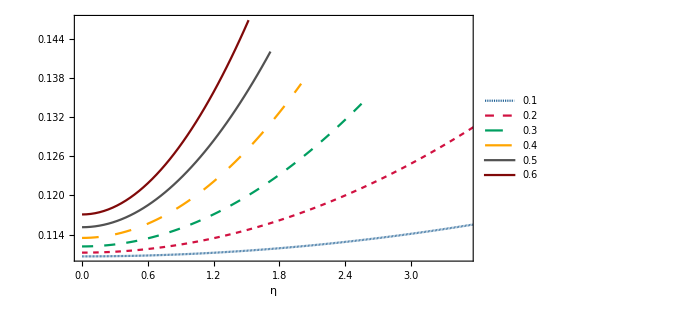

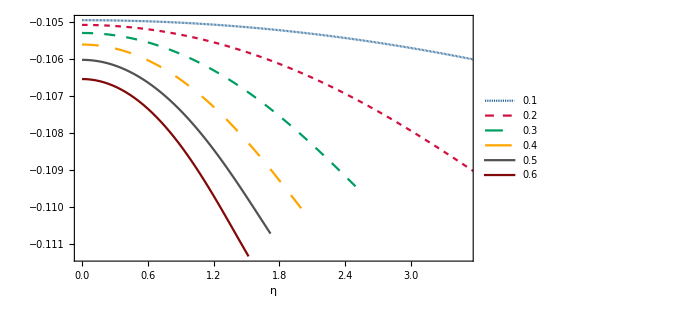

```mathematica
ListLinePlot[{Re[Ts0[[1]]],Re[Ts0[[2]]],Re[Ts0[[3]]],Re[Ts0[[4]]],Re[Ts0[[5]]],Re[Ts0[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.12,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[Ts0[[1]]],Im[Ts0[[2]]],Im[Ts0[[3]]],Im[Ts0[[4]]],Im[Ts0[[5]]],Im[Ts0[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.11,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
(Max[Re[Tsd0[[1]]]]-Min[Re[Tsd0[[1]]]])/Min[Re[Tsd0[[1]]]]*100
(Max[Im[Tsd0[[1]]]]-Min[Im[Tsd0[[1]]]])/Min[Im[Tsd0[[1]]]]*100
(Max[Re[Tsd0[[6]]]]-Min[Re[Tsd0[[6]]]])/Min[Re[Tsd0[[6]]]]*100
(Max[Im[Tsd0[[6]]]]-Min[Im[Tsd0[[6]]]])/Min[Im[Tsd0[[6]]]]*100
```

17.3671

-3.69556

25.4664

-4.31619

#### L=1

```mathematica
Ts0={{{0,0.2934301134681371-0.09771120138843893 ⅈ},{1/25+ⅈ/25,0.29343169713909373-0.09771136409896833 ⅈ},{2/25+(2 ⅈ)/25,0.2934364476047949-0.09771185216837978 ⅈ},{3/25+(3 ⅈ)/25,0.29344436320904826-0.09771266540864466 ⅈ},{4/25+(4 ⅈ)/25,0.29345544119800804-0.09771380350708316 ⅈ},{1/5+ⅈ/5,0.2934696777243245-0.09771526602684465 ⅈ},{6/25+(6 ⅈ)/25,0.2934870678551328-0.09771705240780348 ⅈ},{7/25+(7 ⅈ)/25,0.29350760558225425-0.0977191619677094 ⅈ},{8/25+(8 ⅈ)/25,0.29353128383459387-0.097721593903553 ⅈ},{9/25+(9 ⅈ)/25,0.29355809449260434-0.09772434729322045 ⅈ},{2/5+(2 ⅈ)/5,0.29358802840483766-0.09772742109732704 ⅈ},{11/25+(11 ⅈ)/25,0.2936210754064495-0.09773081416129466 ⅈ},{12/25+(12 ⅈ)/25,0.2936572243395929-0.09773452521763525 ⅈ},{13/25+(13 ⅈ)/25,0.29369646307560904-0.09773855288843439 ⅈ},{14/25+(14 ⅈ)/25,0.29373877853891545-0.09774289568802358 ⅈ},{3/5+(3 ⅈ)/5,0.29378415673248864-0.09774755202582974 ⅈ},{16/25+(16 ⅈ)/25,0.2938325827648322-0.0977525202093889 ⅈ},{17/25+(17 ⅈ)/25,0.293884040878316-0.09775779844751144 ⅈ},{18/25+(18 ⅈ)/25,0.2939385144787703-0.09776338485358516 ⅈ},{19/25+(19 ⅈ)/25,0.29399598616621425-0.09776927744900295 ⅈ},{4/5+(4 ⅈ)/5,0.2940564377665976-0.09777547416670022 ⅈ},{21/25+(21 ⅈ)/25,0.29411985036443195-0.09778197285478929 ⅈ},{22/25+(22 ⅈ)/25,0.2941862043361883-0.09778877128027513 ⅈ},{23/25+(23 ⅈ)/25,0.2942554793843389-0.09779586713283987 ⅈ},{24/25+(24 ⅈ)/25,0.2943276545719203-0.09780325802868094 ⅈ},{1+ⅈ,0.29440270835749877-0.09781094151438999 ⅈ},{26/25+(26 ⅈ)/25,0.29448061863041985-0.09781891507085884 ⅈ},{27/25+(27 ⅈ)/25,0.29456136274622735-0.09782717611719925 ⅈ},{28/25+(28 ⅈ)/25,0.2946449175621427-0.09783572201466431 ⅈ},{29/25+(29 ⅈ)/25,0.29473125947249534-0.0978445500705589 ⅈ},{6/5+(6 ⅈ)/5,0.2948203644440037-0.09785365754212796 ⅈ},{31/25+(31 ⅈ)/25,0.29491220805080925-0.09786304164041101 ⅈ},{32/25+(32 ⅈ)/25,0.2950067655091704-0.09787269953405314 ⅈ},{33/25+(33 ⅈ)/25,0.2951040117117305-0.0978826283530621 ⅈ},{34/25+(34 ⅈ)/25,0.2952039212612795-0.09789282519250261 ⅈ},{7/5+(7 ⅈ)/5,0.2953064685039319-0.09790328711611916 ⅈ},{36/25+(36 ⅈ)/25,0.2954116275616544-0.09791401115988022 ⅈ},{37/25+(37 ⅈ)/25,0.2955193723640782-0.09792499433543547 ⅈ},{38/25+(38 ⅈ)/25,0.29562967667953927-0.09793623363348107 ⅈ},{39/25+(39 ⅈ)/25,0.29574251414529507-0.09794772602702614 ⅈ},{8/5+(8 ⅈ)/5,0.29585785829687267-0.09795946847455624 ⅈ},{41/25+(41 ⅈ)/25,0.2959756825965082-0.09797145792308855 ⅈ},{42/25+(42 ⅈ)/25,0.2960959604606435-0.0979836913111161 ⅈ},{43/25+(43 ⅈ)/25,0.29621866528645174-0.0979961655714371 ⅈ},{44/25+(44 ⅈ)/25,0.29634377047736793-0.09800887763386694 ⅈ},{9/5+(9 ⅈ)/5,0.2964712494676068-0.09802182442783172 ⅈ},{46/25+(46 ⅈ)/25,0.296601075745654-0.09803500288484078 ⅈ},{47/25+(47 ⅈ)/25,0.29673322287672127-0.09804840994083824 ⅈ},{48/25+(48 ⅈ)/25,0.29686766452416186-0.09806204253843293 ⅈ},{49/25+(49 ⅈ)/25,0.29700437446984423-0.09807589762900652 ⅈ},{2+2 ⅈ,0.2971433266334879-0.09808997217470097 ⅈ},{51/25+(51 ⅈ)/25,0.2972844950909678-0.09810426315028542 ⅈ},{52/25+(52 ⅈ)/25,0.2974278540915964-0.09811876754490483 ⅈ},{53/25+(53 ⅈ)/25,0.2975733780743967-0.09813348236371078 ⅈ},{54/25+(54 ⅈ)/25,0.29772104168338104-0.09814840462937739 ⅈ},{11/5+(11 ⅈ)/5,0.29787081978185315-0.09816353138350398 ⅈ},{56/25+(56 ⅈ)/25,0.29802268746575383-0.09817885968790706 ⅈ},{57/25+(57 ⅈ)/25,0.29817662007607143-0.0981943866258041 ⅈ},{58/25+(58 ⅈ)/25,0.2983325932103401-0.0982101093028924 ⅈ},{59/25+(59 ⅈ)/25,0.2984905827332515-0.09822602484832527 ⅈ},{12/5+(12 ⅈ)/5,0.2986505647864048-0.09824213041558946 ⅈ},{61/25+(61 ⅈ)/25,0.29881251579722234-0.09825842318328648 ⅈ},{62/25+(62 ⅈ)/25,0.29897641248705925-0.09827490035582125 ⅈ},{63/25+(63 ⅈ)/25,0.29914223187853395-0.09829155916400174 ⅈ},{64/25+(64 ⅈ)/25,0.2993099513021096-0.09830839686555261 ⅈ},{13/5+(13 ⅈ)/5,0.29947954840195495-0.09832541074554663 ⅈ},{66/25+(66 ⅈ)/25,0.2996510011411142-0.09834259811675729 ⅈ},{67/25+(67 ⅈ)/25,0.29982428780601467-0.0983599563199359 ⅈ},{68/25+(68 ⅈ)/25,0.29999938701034207-0.09837748272401683 ⅈ},{69/25+(69 ⅈ)/25,0.30017627769831157-0.09839517472625449 ⅈ},{14/5+(14 ⅈ)/5,0.3003549391473643-0.09841302975229464 ⅈ},{71/25+(71 ⅈ)/25,0.3005353509703169-0.09843104525618482 ⅈ},{72/25+(72 ⅈ)/25,0.3007174931169919-0.09844921872032553 ⅈ},{73/25+(73 ⅈ)/25,0.300901345875357-0.09846754765536676 ⅈ},{74/25+(74 ⅈ)/25,0.30108688987219867-0.09848602960005219 ⅈ},{3+3 ⅈ,0.3012741060733581-0.09850466212101452 ⅈ},{76/25+(76 ⅈ)/25,0.30146297578355213-0.09852344281252491 ⅈ},{77/25+(77 ⅈ)/25,0.30165348064580694-0.09854236929619929 ⅈ},{78/25+(78 ⅈ)/25,0.3018456026405254-0.09856143922066452 ⅈ},{79/25+(79 ⅈ)/25,0.302039324084214-0.09858065026118693 ⅈ},{16/5+(16 ⅈ)/5,0.30223462762788944-0.09860000011926644 ⅈ},{81/25+(81 ⅈ)/25,0.30243149625518767-0.09861948652219785 ⅈ},{82/25+(82 ⅈ)/25,0.30262991328019584-0.09863910722260287 ⅈ},{83/25+(83 ⅈ)/25,0.3028298623450269-0.09865885999793442 ⅈ},{84/25+(84 ⅈ)/25,0.30303132741715616-0.09867874264995578 ⅈ},{17/5+(17 ⅈ)/5,0.3032342927865381-0.09869875300419678 ⅈ},{86/25+(86 ⅈ)/25,0.30343874306252033-0.09871888890938922 ⅈ},{87/25+(87 ⅈ)/25,0.3036446631705731-0.0987391482368832 ⅈ},{88/25+(88 ⅈ)/25,0.3038520383488473-0.09875952888004648 ⅈ},{89/25+(89 ⅈ)/25,0.30406085414457984-0.09878002875364886 ⅈ},{18/5+(18 ⅈ)/5,0.3042710964103574-0.0988006457932327 ⅈ},{91/25+(91 ⅈ)/25,0.30448275130025426-0.09882137795447202 ⅈ},{92/25+(92 ⅈ)/25,0.3046958052658569-0.0988422232125212 ⅈ},{93/25+(93 ⅈ)/25,0.3049102450521866-0.09886317956135486 ⅈ},{94/25+(94 ⅈ)/25,0.30512605769353324-0.09888424501310046 ⅈ},{19/5+(19 ⅈ)/5,0.30534323050920964-0.09890541759736485 ⅈ},{96/25+(96 ⅈ)/25,0.305561751099238-0.09892669536055612 ⅈ},{97/25+(97 ⅈ)/25,0.30578160733997783-0.09894807636520174 ⅈ},{98/25+(98 ⅈ)/25,0.3060027873797036-0.09896955868926446 ⅈ},{99/25+(99 ⅈ)/25,0.3062252796341423-0.09899114042545666 ⅈ},{4+4 ⅈ,0.3064490727819775-0.09901281968055443 ⅈ},{101/25+(101 ⅈ)/25,0.30667415576032864-0.09903459457471216 ⅈ},{102/25+(102 ⅈ)/25,0.30690051776021093-0.09905646324077858 ⅈ},{103/25+(103 ⅈ)/25,0.3071281482219848-0.09907842382361523 ⅈ},{104/25+(104 ⅈ)/25,0.3073570368307986-0.0991004744794177 ⅈ},{21/5+(21 ⅈ)/5,0.307587173512032-0.09912261337504105 ⅈ},{106/25+(106 ⅈ)/25,0.30781854842674383-0.09914483868732944 ⅈ},{107/25+(107 ⅈ)/25,0.30805115196713123-0.09916714860245093 ⅈ},{108/25+(108 ⅈ)/25,0.3082849747520024-0.0991895413152382 ⅈ},{109/25+(109 ⅈ)/25,0.3085200076222691-0.09921201502853541 ⅈ},{22/5+(22 ⅈ)/5,0.308756241636461-0.0992345679525519 ⅈ},{111/25+(111 ⅈ)/25,0.3089936680662667-0.09925719830422326 ⅈ},{112/25+(112 ⅈ)/25,0.30923227839210454-0.09927990430658014 ⅈ},{113/25+(113 ⅈ)/25,0.30947206429872487-0.09930268418812534 ⅈ},{114/25+(114 ⅈ)/25,0.3097130176708482-0.09932553618221929 ⅈ},{23/5+(23 ⅈ)/5,0.3099551305888404-0.09934845852647477 ⅈ},{116/25+(116 ⅈ)/25,0.3101983953244278-0.0993714494621607 ⅈ},{117/25+(117 ⅈ)/25,0.3104428043364542-0.0993945072336157 ⅈ},{118/25+(118 ⅈ)/25,0.31068835026668057-0.09941763008767147 ⅈ},{119/25+(119 ⅈ)/25,0.3109350259356306-0.09944081627308644 ⅈ},{24/5+(24 ⅈ)/5,0.3111828243384824-0.09946406403998975 ⅈ},{121/25+(121 ⅈ)/25,0.3114317386410077-0.09948737163933594 ⅈ},{122/25+(122 ⅈ)/25,0.31168176217556004-0.09951073732237066 ⅈ},{123/25+(123 ⅈ)/25,0.31193288843711225-0.09953415934010713 ⅈ},{124/25+(124 ⅈ)/25,0.31218511107934493-0.09955763594281423 ⅈ},{5+5 ⅈ,0.3124384239107856-0.09958116537951577 ⅈ},{126/25+(126 ⅈ)/25,0.3126928208909993-0.09960474589750133 ⅈ},{127/25+(127 ⅈ)/25,0.31294829612683206-0.099628375741849 ⅈ},{128/25+(128 ⅈ)/25,0.31320484386870573-0.09965205315495979 ⅈ},{129/25+(129 ⅈ)/25,0.31346245850696597-0.09967577637610403 ⅈ},{26/5+(26 ⅈ)/5,0.31372113456828316-0.09969954364097991 ⅈ},{131/25+(131 ⅈ)/25,0.31398086671210534-0.09972335318128414 ⅈ},{132/25+(132 ⅈ)/25,0.3142416497271652-0.09974720322429473 ⅈ},{133/25+(133 ⅈ)/25,0.31450347852803795-0.09977109199246632 ⅈ},{134/25+(134 ⅈ)/25,0.3147663481517536-0.09979501770303782 ⅈ},{27/5+(27 ⅈ)/5,0.3150302537544603-0.09981897856765237 ⅈ},{136/25+(136 ⅈ)/25,0.3152951906081405-0.09984297279199006 ⅈ},{137/25+(137 ⅈ)/25,0.3155611540973782-0.09986699857541297 ⅈ},{138/25+(138 ⅈ)/25,0.31582813971617857-0.09989105411062306 ⅈ},{139/25+(139 ⅈ)/25,0.31609614306483746-0.09991513758333263 ⅈ},{28/5+(28 ⅈ)/5,0.3163651598468626-0.09993924717194724 ⅈ},{141/25+(141 ⅈ)/25,0.3166351858659442-0.0999633810472618 ⅈ},{142/25+(142 ⅈ)/25,0.31690621702297594-0.09998753737216899 ⅈ},{143/25+(143 ⅈ)/25,0.3171782493131245-0.10001171430138062 ⅈ},{144/25+(144 ⅈ)/25,0.3174512788229482-0.10003590998116184 ⅈ},{29/5+(29 ⅈ)/5,0.3177253017275637-0.1000601225490779 ⅈ},{146/25+(146 ⅈ)/25,0.3180003142878599-0.10008435013375411 ⅈ},{147/25+(147 ⅈ)/25,0.3182763128477597-0.10010859085464806 ⅈ},{148/25+(148 ⅈ)/25,0.31855329383152725-0.10013284282183527 ⅈ},{149/25+(149 ⅈ)/25,0.3188312537411218-0.10015710413580707 ⅈ},{6+6 ⅈ,0.3191101891535962-0.1001813728872818 ⅈ},{151/25+(151 ⅈ)/25,0.3193900967185407-0.10020564715702841 ⅈ},{152/25+(152 ⅈ)/25,0.31967097315557-0.10022992501570308 ⅈ},{153/25+(153 ⅈ)/25,0.3199528152518548-0.10025420452369857 ⅈ},{154/25+(154 ⅈ)/25,0.3202356198596951-0.10027848373100628 ⅈ},{31/5+(31 ⅈ)/5,0.32051938389413664-0.10030276067709123 ⅈ},{156/25+(156 ⅈ)/25,0.3208041043306281-0.10032703339077961 ⅈ},{157/25+(157 ⅈ)/25,0.32108977820272083-0.10035129989015902 ⅈ},{158/25+(158 ⅈ)/25,0.321376402599807-0.10037555818249155 ⅈ},{159/25+(159 ⅈ)/25,0.3216639746648995-0.10039980626413952 ⅈ},{32/5+(32 ⅈ)/5,0.32195249159245004-0.10042404212050367 ⅈ},{161/25+(161 ⅈ)/25,0.3222419506262064-0.10044826372597408 ⅈ},{162/25+(162 ⅈ)/25,0.3225323490571079-0.10047246904389372 ⅈ},{163/25+(163 ⅈ)/25,0.32282368422121804-0.10049665602653436 ⅈ},{164/25+(164 ⅈ)/25,0.32311595349769473-0.10052082261508516 ⅈ},{33/5+(33 ⅈ)/5,0.32340915430679673-0.10054496673965355 ⅈ},{166/25+(166 ⅈ)/25,0.32370328410792626-0.10056908631927863 ⅈ},{167/25+(167 ⅈ)/25,0.32399834039770714-0.10059317926195681 ⅈ},{168/25+(168 ⅈ)/25,0.32429432070809755-0.10061724346467996 ⅈ},{169/25+(169 ⅈ)/25,0.32459122260453765-0.10064127681348548 ⅈ},{34/5+(34 ⅈ)/5,0.32488904368413113-0.10066527718351895 ⅈ},{171/25+(171 ⅈ)/25,0.3251877815738601-0.10068924243910864 ⅈ},{172/25+(172 ⅈ)/25,0.3254874339288332-0.10071317043385208 ⅈ},{173/25+(173 ⅈ)/25,0.3257879984305665-0.10073705901071502 ⅈ},{174/25+(174 ⅈ)/25,0.326089472785296-0.10076090600214165 ⅈ},{7+7 ⅈ,0.32639185472232246-0.1007847092301774 ⅈ},{176/25+(176 ⅈ)/25,0.32669514199238747-0.10080846650660308 ⅈ},{177/25+(177 ⅈ)/25,0.32699933236607986-0.1008321756330808 ⅈ},{178/25+(178 ⅈ)/25,0.32730442363227374-0.10085583440131156 ⅈ}},{{0,0.29490584811772586-0.09786585160959349 ⅈ},{1/25+ⅈ/25,0.29491219900450055-0.09786649202768732 ⅈ},{2/25+(2 ⅈ)/25,0.2949312426284681-0.09786841227206068 ⅈ},{3/25+(3 ⅈ)/25,0.2949629518941012-0.09787160931505241 ⅈ},{4/25+(4 ⅈ)/25,0.29500728190800235-0.09787607813989795 ⅈ},{1/5+ⅈ/5,0.2950641703503-0.09788181178185781 ⅈ},{6/25+(6 ⅈ)/25,0.2951335379933918-0.09788880138558463 ⅈ},{7/25+(7 ⅈ)/25,0.29521528935202446-0.09789703627696546 ⅈ},{8/25+(8 ⅈ)/25,0.2953093134528352-0.0979065040481005 ⅈ},{9/25+(9 ⅈ)/25,0.2954154847096546-0.09791719065386921 ⅈ},{2/5+(2 ⅈ)/5,0.29553366388947694-0.09792908051837845 ⅈ},{11/25+(11 ⅈ)/25,0.29566369915305174-0.09794215664948014 ⅈ},{12/25+(12 ⅈ)/25,0.2958054271535533-0.0979564007594922 ⅈ},{13/25+(13 ⅈ)/25,0.2959586741767196-0.09797179339025028 ⅈ},{14/25+(14 ⅈ)/25,0.2961232573061957-0.0979883140406585 ⅈ},{3/5+(3 ⅈ)/5,0.29629898559851514-0.09800594129498968 ⅈ},{16/25+(16 ⅈ)/25,0.29648566125316517-0.09802465295029991 ⅈ},{17/25+(17 ⅈ)/25,0.29668308076443006-0.0980444261414676 ⅈ},{18/25+(18 ⅈ)/25,0.2968910360431459-0.09806523746253092 ⅈ},{19/25+(19 ⅈ)/25,0.2971093154980569-0.098087063083174 ⅈ},{4/5+(4 ⅈ)/5,0.29733770506808-0.09810987885939958 ⅈ},{21/25+(21 ⅈ)/25,0.297575989198414-0.09813366043760763 ⅈ},{22/25+(22 ⅈ)/25,0.29782395175501875-0.09815838335148251 ⅈ},{23/25+(23 ⅈ)/25,0.29808137687350156-0.09818402311126227 ⅈ},{24/25+(24 ⅈ)/25,0.29834804973985934-0.09821055528512249 ⅈ},{1+ⅈ,0.2986237573018011-0.09823795557255308 ⅈ},{26/25+(26 ⅈ)/25,0.29890828891051485-0.09826619986973319 ⅈ},{27/25+(27 ⅈ)/25,0.29920143689373063-0.09829526432702566 ⅈ},{28/25+(28 ⅈ)/25,0.29950299706176553-0.09832512539879106 ⅈ},{29/25+(29 ⅈ)/25,0.2998127691489292-0.09835575988582877 ⅈ},{6/5+(6 ⅈ)/5,0.3001305571932107-0.09838714497077589 ⅈ},{31/25+(31 ⅈ)/25,0.3004561698575899-0.0984192582468714 ⅈ},{32/25+(32 ⅈ)/25,0.3007894206966093-0.0984520777405104 ⅈ},{33/25+(33 ⅈ)/25,0.30113012837204134-0.09848558192803897 ⅈ},{34/25+(34 ⅈ)/25,0.3014781168215798-0.0985197497472492 ⅈ},{7/5+(7 ⅈ)/5,0.3018332153845122-0.09855456060403696 ⅈ},{36/25+(36 ⅈ)/25,0.30219525888828147-0.09858999437467762 ⅈ},{37/25+(37 ⅈ)/25,0.30256408769975396-0.09862603140416491 ⅈ},{38/25+(38 ⅈ)/25,0.3029395477448662-0.09866265250104016 ⅈ},{39/25+(39 ⅈ)/25,0.3033214905001569-0.09869983892912079 ⅈ},{8/5+(8 ⅈ)/5,0.3037097729594935-0.09873757239651279 ⅈ},{41/25+(41 ⅈ)/25,0.3041042575790952-0.09877583504226944 ⅈ},{42/25+(42 ⅈ)/25,0.30450481220373443-0.09881460942103226 ⅈ},{43/25+(43 ⅈ)/25,0.3049113099767767-0.09885387848596532 ⅈ},{44/25+(44 ⅈ)/25,0.30532362923649986-0.09889362557026843 ⅈ},{9/5+(9 ⅈ)/5,0.30574165340091297-0.09893383436753075 ⅈ},{46/25+(46 ⅈ)/25,0.3061652708430901-0.09897448891116166 ⅈ},{47/25+(47 ⅈ)/25,0.30659437475882917-0.09901557355311347 ⅈ},{48/25+(48 ⅈ)/25,0.30702886302826166-0.09905707294208964 ⅈ},{49/25+(49 ⅈ)/25,0.30746863807285496-0.09909897200141045 ⅈ},{2+2 ⅈ,0.30791360670908885-0.09914125590669169 ⅈ},{51/25+(51 ⅈ)/25,0.30836367999993053-0.09918391006347246 ⅈ},{52/25+(52 ⅈ)/25,0.30881877310509326-0.09922692008491386 ⅈ},{53/25+(53 ⅈ)/25,0.3092788051309344-0.09927027176967507 ⅈ},{54/25+(54 ⅈ)/25,0.30974369898073184-0.09931395108006111 ⅈ},{11/5+(11 ⅈ)/5,0.3102133812059702-0.09935794412052328 ⅈ},{56/25+(56 ⅈ)/25,0.31068778185917645-0.09940223711658445 ⅈ},{57/25+(57 ⅈ)/25,0.311166834348755-0.09944681639425057 ⅈ},{58/25+(58 ⅈ)/25,0.31165047529619816-0.09949166835996173 ⅈ},{59/25+(59 ⅈ)/25,0.3121386443959822-0.09953677948112857 ⅈ},{12/5+(12 ⅈ)/5,0.312631284278394-0.09958213626729355 ⅈ},{61/25+(61 ⅈ)/25,0.3131283403754869-0.09962772525195002 ⅈ},{62/25+(62 ⅈ)/25,0.31362976079031496-0.09967353297504776 ⅈ},{63/25+(63 ⅈ)/25,0.3141354961695538-0.09971954596620869 ⅈ},{64/25+(64 ⅈ)/25,0.31464549957958554-0.09976575072867228 ⅈ},{13/5+(13 ⅈ)/5,0.31515972638609097-0.09981213372398814 ⅈ},{66/25+(66 ⅈ)/25,0.3156781341371692-0.09985868135746848 ⅈ},{67/25+(67 ⅈ)/25,0.3162006824499836-0.09990537996441254 ⅈ},{68/25+(68 ⅈ)/25,0.31672733290091193-0.09995221579711101 ⅈ},{69/25+(69 ⅈ)/25,0.31725804891916626-0.09999917501263896 ⅈ},{14/5+(14 ⅈ)/5,0.3177927956838345-0.10004624366144144 ⅈ},{71/25+(71 ⅈ)/25,0.31833154002428454-0.10009340767671718 ⅈ},{72/25+(72 ⅈ)/25,0.3188742503238652-0.10014065286460298 ⅈ},{73/25+(73 ⅈ)/25,0.3194208964268311-0.10018796489516085 ⅈ},{74/25+(74 ⅈ)/25,0.31997144954841433-0.10023532929416938 ⅈ},{3+3 ⅈ,0.32052588218796163-0.10028273143571972 ⅈ},{76/25+(76 ⅈ)/25,0.3210841680450549-0.10033015653561564 ⅈ},{77/25+(77 ⅈ)/25,0.32164628193853123-0.1003775896455777 ⅈ},{78/25+(78 ⅈ)/25,0.32221219972831766-0.10042501564824893 ⅈ},{79/25+(79 ⅈ)/25,0.32278189823999703-0.10047241925300103 ⅈ},{16/5+(16 ⅈ)/5,0.32335535519202363-0.10051978499253834 ⅈ},{81/25+(81 ⅈ)/25,0.3239325491255055-0.10056709722029629 ⅈ},{82/25+(82 ⅈ)/25,0.32451345933647685-0.10061434010863111 ⅈ},{83/25+(83 ⅈ)/25,0.3250980658105819-0.10066149764779685 ⅈ},{84/25+(84 ⅈ)/25,0.3256863491600984-0.10070855364570433 ⅈ},{17/5+(17 ⅈ)/5,0.32627829056322755-0.10075549172845802 ⅈ},{86/25+(86 ⅈ)/25,0.32687387170558446-0.10080229534166345 ⅈ},{87/25+(87 ⅈ)/25,0.32747307472382287-0.10084894775249993 ⅈ},{88/25+(88 ⅈ)/25,0.32807588215133304-0.1008954320525505 ⅈ},{89/25+(89 ⅈ)/25,0.32868227686595397-0.10094173116138144 ⅈ},{18/5+(18 ⅈ)/5,0.32929224203964486-0.10098782783086216 ⅈ},{91/25+(91 ⅈ)/25,0.32990576109006386-0.10103370465021622 ⅈ}},{{0,0.29734494056573973-0.09812674596109573 ⅈ},{1/25+ⅈ/25,0.29735929784812914-0.09812814977365117 ⅈ},{2/25+(2 ⅈ)/25,0.2974023218855444-0.09813235600258753 ⅈ},{3/25+(3 ⅈ)/25,0.2974738700498331-0.09813934911006285 ⅈ},{4/25+(4 ⅈ)/25,0.29757370775841435-0.09814910353858253 ⅈ},{1/5+ⅈ/5,0.29770151297674835-0.09816158419856044 ⅈ},{6/25+(6 ⅈ)/25,0.29785688226588203-0.098176747122357 ⅈ},{7/25+(7 ⅈ)/25,0.29803933811016897-0.0981945402557148 ⅈ},{8/25+(8 ⅈ)/25,0.2982483372360469-0.09821490435467384 ⅈ},{9/25+(9 ⅈ)/25,0.2984832796136153-0.09823777395396598 ⅈ},{2/5+(2 ⅈ)/5,0.29874351783253933-0.09826307837290545 ⅈ},{11/25+(11 ⅈ)/25,0.29902836656037246-0.09829074272666875 ⅈ},{12/25+(12 ⅈ)/25,0.29933711182138706-0.09832068891421838 ⅈ},{13/25+(13 ⅈ)/25,0.2996690198734464-0.09835283655852878 ⅈ},{14/25+(14 ⅈ)/25,0.30002334550524684-0.09838710387975928 ⅈ},{3/5+(3 ⅈ)/5,0.30039933962259424-0.09842340848717118 ⅈ},{16/25+(16 ⅈ)/25,0.300796256037107-0.09846166808054722 ⅈ},{17/25+(17 ⅈ)/25,0.30121335741145616-0.09850180105638345 ⅈ},{18/25+(18 ⅈ)/25,0.30164992035040517-0.09854372701800863 ⅈ},{19/25+(19 ⅈ)/25,0.3021052396556886-0.09858736719196079 ⅈ},{4/5+(4 ⅈ)/5,0.30257863178500294-0.09863264475539434 ⅈ},{21/25+(21 ⅈ)/25,0.30306943757138055-0.09867948508104321 ⅈ},{22/25+(22 ⅈ)/25,0.30357702426962535-0.0987278159073952 ⅈ},{23/25+(23 ⅈ)/25,0.3041007870021196-0.09877756744233458 ⅈ},{24/25+(24 ⅈ)/25,0.3046401496780674-0.09882867240868397 ⅈ},{1+ⅈ,0.30519456545899853-0.09888106603991949 ⅈ},{26/25+(26 ⅈ)/25,0.30576351683992237-0.09893468603393664 ⅈ},{27/25+(27 ⅈ)/25,0.3063465154106023-0.0989894724721834 ⅈ},{28/25+(28 ⅈ)/25,0.3069431013555997-0.0990453677108303 ⅈ},{29/25+(29 ⅈ)/25,0.3075528427454783-0.09910231624992695 ⅈ},{6/5+(6 ⅈ)/5,0.3081753346652187-0.09916026458580993 ⅈ},{31/25+(31 ⅈ)/25,0.30881019821972944-0.09921916105132242 ⅈ},{32/25+(32 ⅈ)/25,0.3094570794505263-0.09927895564776985 ⅈ},{33/25+(33 ⅈ)/25,0.31011564819230103-0.09933959987194035 ⅈ},{34/25+(34 ⅈ)/25,0.31078559689326896-0.09940104654098664 ⅈ},{7/5+(7 ⅈ)/5,0.31146663941889535-0.09946324961749359 ⅈ},{36/25+(36 ⅈ)/25,0.31215850985484545-0.09952616403664298 ⅈ},{37/25+(37 ⅈ)/25,0.312860961321758-0.09958974553703275 ⅈ},{38/25+(38 ⅈ)/25,0.3135737648116692-0.09965395049640546 ⅈ},{39/25+(39 ⅈ)/25,0.3142967080535734-0.0997187357732856 ⅈ},{8/5+(8 ⅈ)/5,0.31502959441364514-0.09978405855531357 ⅈ},{41/25+(41 ⅈ)/25,0.31577224183403135-0.09984987621488906 ⅈ},{42/25+(42 ⅈ)/25,0.3165244818127929-0.0999161461725935 ⅈ},{43/25+(43 ⅈ)/25,0.317286158426505-0.09998282576874568 ⅈ},{44/25+(44 ⅈ)/25,0.31805712739616837-0.10004987214335222 ⅈ},{9/5+(9 ⅈ)/5,0.3188372551964123-0.10011724212464151 ⅈ},{46/25+(46 ⅈ)/25,0.31962641820744825-0.10018489212631268 ⅈ},{47/25+(47 ⅈ)/25,0.32042450190884353-0.10025277805358622 ⅈ},{48/25+(48 ⅈ)/25,0.32123140011389667-0.10032085521810985 ⅈ},{49/25+(49 ⅈ)/25,0.3220470142431965-0.1003890782617461 ⅈ},{2+2 ⅈ,0.32287125263581645-0.10045740108924965 ⅈ},{51/25+(51 ⅈ)/25,0.32370402989652464-0.10052577680982618 ⅈ},{52/25+(52 ⅈ)/25,0.3245452662773571-0.10059415768755342 ⅈ},{53/25+(53 ⅈ)/25,0.3253948870919135-0.10066249510063437 ⅈ},{54/25+(54 ⅈ)/25,0.32625282216076534-0.10073073950944489 ⅈ},{11/5+(11 ⅈ)/5,0.32711900528642185-0.10079884043332847 ⅈ},{56/25+(56 ⅈ)/25,0.3279933737563704-0.10086674643608326 ⅈ},{57/25+(57 ⅈ)/25,0.32887586787278594-0.10093440512007558 ⅈ},{58/25+(58 ⅈ)/25,0.32976643050759485-0.1010017631289053 ⅈ},{59/25+(59 ⅈ)/25,0.3306650066816675-0.10106876615853388 ⅈ},{12/5+(12 ⅈ)/5,0.3315715431670091-0.10113535897677436 ⅈ},{61/25+(61 ⅈ)/25,0.3324859881109104-0.1012014854510242 ⅈ},{62/25+(62 ⅈ)/25,0.3334082906811114-0.10126708858410645 ⅈ},{63/25+(63 ⅈ)/25,0.3343384007311194-0.10133211055806286 ⅈ},{64/25+(64 ⅈ)/25,0.33527626848490716-0.10139649278572198 ⅈ}},{{0,0.30071745721129695-0.09849783114098085 ⅈ},{1/25+ⅈ/25,0.3007431768142335-0.09850024163397418 ⅈ},{2/25+(2 ⅈ)/25,0.3008201747381251-0.09850745615434196 ⅈ},{3/25+(3 ⅈ)/25,0.3009479739781611-0.09851942442480774 ⅈ},{4/25+(4 ⅈ)/25,0.30112579877410495-0.09853606467738138 ⅈ},{1/5+ⅈ/5,0.30135260176114-0.09855726651118493 ⅈ},{6/25+(6 ⅈ)/25,0.3016270989931223-0.0985828945724999 ⅈ},{7/25+(7 ⅈ)/25,0.30194781029049117-0.09861279278439561 ⅈ},{8/25+(8 ⅈ)/25,0.3023131022687132-0.09864678884293436 ⅈ},{9/25+(9 ⅈ)/25,0.30272123156009245-0.0986846987141775 ⅈ},{2/5+(2 ⅈ)/5,0.30317038611120345-0.09872633090625724 ⅈ},{11/25+(11 ⅈ)/25,0.30365872293419366-0.09877149034435627 ⅈ},{12/25+(12 ⅈ)/25,0.30418440122764345-0.09881998173438179 ⅈ},{13/25+(13 ⅈ)/25,0.30474561029189134-0.09887161235592848 ⅈ},{14/25+(14 ⅈ)/25,0.30534059209774417-0.09892619427175403 ⅈ},{3/5+(3 ⅈ)/5,0.30596765870266307-0.09898354597691754 ⅈ},{16/25+(16 ⅈ)/25,0.3066252049406153-0.09904349353551994 ⅈ},{17/25+(17 ⅈ)/25,0.307311716950059-0.09910587126766228 ⅈ},{18/25+(18 ⅈ)/25,0.30802577716569063-0.09917052205561365 ⅈ},{19/25+(19 ⅈ)/25,0.3087660664028806-0.09923729733834671 ⅈ},{4/5+(4 ⅈ)/5,0.3095313636275728-0.09930605685954702 ⅈ},{21/25+(21 ⅈ)/25,0.3103205439445363-0.0993766682276274 ⅈ},{22/25+(22 ⅈ)/25,0.3111325752654642-0.09944900633849961 ⅈ},{23/25+(23 ⅈ)/25,0.3119665140443152-0.09952295270381732 ⅈ},{24/25+(24 ⅈ)/25,0.31282150039629525-0.09959839471973116 ⅈ},{1+ⅈ,0.31369675285238763-0.09967522490424538 ⅈ},{26/25+(26 ⅈ)/25,0.3145915629450364-0.09975334012522188 ⅈ},{27/25+(27 ⅈ)/25,0.3155052897729228-0.09983264083596359 ⅈ},{28/25+(28 ⅈ)/25,0.316437354653431-0.09991303033115435 ⅈ},{29/25+(29 ⅈ)/25,0.3173872359396703-0.09999441403248546 ⅈ},{6/5+(6 ⅈ)/5,0.3183544640537946-0.10007669881074681 ⅈ},{31/25+(31 ⅈ)/25,0.3193386167689067-0.10015979234903667 ⅈ},{32/25+(32 ⅈ)/25,0.32033931475703165-0.10024360255024195 ⅈ},{33/25+(33 ⅈ)/25,0.3213562174096474-0.10032803699078773 ⅈ},{34/25+(34 ⅈ)/25,0.32238901892929417-0.10041300242183557 ⅈ},{7/5+(7 ⅈ)/5,0.323437444685208-0.10049840431853431 ⅈ},{36/25+(36 ⅈ)/25,0.3245012478221938-0.10058414647753852 ⅈ},{37/25+(37 ⅈ)/25,0.32558020610963767-0.10067013066275847 ⅈ},{38/25+(38 ⅈ)/25,0.326674119016308-0.10075625629915182 ⅈ},{39/25+(39 ⅈ)/25,0.3277828049961261-0.10084242021427944 ⅈ},{8/5+(8 ⅈ)/5,0.3289060989701914-0.1009285164273028 ⅈ},{41/25+(41 ⅈ)/25,0.3300438499908466-0.10101443598507263 ⅈ},{42/25+(42 ⅈ)/25,0.331195919074345-0.10110006684494344 ⅈ},{43/25+(43 ⅈ)/25,0.3323621771896246-0.10118529380392187 ⅈ},{44/25+(44 ⅈ)/25,0.33354250339174574-0.10126999847372016 ⅈ},{9/5+(9 ⅈ)/5,0.3347367830896326-0.10135405930122783 ⅈ},{46/25+(46 ⅈ)/25,0.3359449064388549-0.10143735163383216 ⅈ},{47/25+(47 ⅈ)/25,0.33716676685125113-0.10151974782890706 ⅈ},{48/25+(48 ⅈ)/25,0.3384022596142109-0.1016011174066525 ⅈ},{49/25+(49 ⅈ)/25,0.3396512806133858-0.10168132724529799 ⅈ},{2+2 ⅈ,0.34091372515347773-0.10176024181748942 ⅈ}},{{0,0.3049829820416122-0.09898323828394866 ⅈ},{1/25+ⅈ/25,0.305023636495005-0.09898685265561466 ⅈ},{2/25+(2 ⅈ)/25,0.3051451725153767-0.09899765240747944 ⅈ},{3/25+(3 ⅈ)/25,0.3053463336829677-0.09901551007006261 ⅈ},{4/25+(4 ⅈ)/25,0.3056251092001341-0.09904022168865727 ⅈ},{1/5+ⅈ/5,0.30597884710713347-0.09907151836016619 ⅈ},{6/25+(6 ⅈ)/25,0.3064043925408542-0.09910908028533129 ⅈ},{7/25+(7 ⅈ)/25,0.30689823603268207-0.09915255178367499 ⅈ},{8/25+(8 ⅈ)/25,0.30745665826900254-0.09920155586830567 ⅈ},{9/25+(9 ⅈ)/25,0.30807586089091893-0.09925570730721534 ⅈ},{2/5+(2 ⅈ)/5,0.3087520767894539-0.09931462350206371 ⅈ},{11/25+(11 ⅈ)/25,0.30948165705955094-0.09937793290109737 ⅈ},{12/25+(12 ⅈ)/25,0.3102611347420168-0.09944528097074576 ⅈ},{13/25+(13 ⅈ)/25,0.3110872674892599-0.09951633395809825 ⅈ},{14/25+(14 ⅈ)/25,0.3119570623839356-0.0995907807888751 ⅈ},{3/5+(3 ⅈ)/5,0.3128677865088622-0.09966833348258548 ⅈ},{16/25+(16 ⅈ)/25,0.3138169667436628-0.09974872645257968 ⅈ},{17/25+(17 ⅈ)/25,0.31480238185884785-0.09983171501563151 ⅈ},{18/25+(18 ⅈ)/25,0.31582204945200115-0.0999170733802597 ⅈ},{19/25+(19 ⅈ)/25,0.31687420973004954-0.10000459232630958 ⅈ},{4/5+(4 ⅈ)/5,0.3179573076474705-0.10009407673670498 ⅈ},{21/25+(21 ⅈ)/25,0.3190699744909827-0.1001853430986434 ⅈ},{22/25+(22 ⅈ)/25,0.3202110096637927-0.10027821705653259 ⅈ},{23/25+(23 ⅈ)/25,0.3213793631619474-0.10037253107210084 ⅈ},{24/25+(24 ⅈ)/25,0.32257411904120203-0.10046812222722146 ⅈ},{1+ⅈ,0.32379448003283984-0.10056483019076994 ⅈ},{26/25+(26 ⅈ)/25,0.3250397533692981-0.10066249536102831 ⅈ},{27/25+(27 ⅈ)/25,0.3263093378150464-0.10076095718864414 ⅈ},{28/25+(28 ⅈ)/25,0.32760271185637496-0.10086005268119752 ⅈ},{29/25+(29 ⅈ)/25,0.3289194229792258-0.10095961508788824 ⅈ},{6/5+(6 ⅈ)/5,0.33025907795135806-0.10105947276194199 ⅈ},{31/25+(31 ⅈ)/25,0.33162133402078325-0.10115944819771636 ⅈ},{32/25+(32 ⅈ)/25,0.33300589094326954-0.10125935723963227 ⅈ},{33/25+(33 ⅈ)/25,0.3344124837560968-0.10135900846030095 ⅈ},{34/25+(34 ⅈ)/25,0.33584087622163983-0.10145820270556648 ⅈ},{7/5+(7 ⅈ)/5,0.337290854871819-0.10155673280449068 ⅈ},{36/25+(36 ⅈ)/25,0.3387622235923282-0.10165438344249586 ⅈ},{37/25+(37 ⅈ)/25,0.34025479869339126-0.10175093119589781 ⅈ},{38/25+(38 ⅈ)/25,0.34176840442132495-0.10184614472587507 ⅈ},{39/25+(39 ⅈ)/25,0.3433028688722289-0.10193978512951056 ⅈ},{8/5+(8 ⅈ)/5,0.3448580202755622-0.10203160644490282 ⅈ},{41/25+(41 ⅈ)/25,0.34643368362115873-0.10212135630647981 ⅈ},{42/25+(42 ⅈ)/25,0.34802967760833364-0.1022087767455709 ⅈ},{43/25+(43 ⅈ)/25,0.3496458119001519-0.10229360513002358 ⅈ}},{{0,0.31009201405974723-0.09958619259031025 ⅈ},{1/25+ⅈ/25,0.3101515544864499-0.09959117111682296 ⅈ},{2/25+(2 ⅈ)/25,0.3103291871653887-0.09960601030665815 ⅈ},{3/25+(3 ⅈ)/25,0.3106220390846032-0.0996304301752686 ⅈ},{4/25+(4 ⅈ)/25,0.3110256138599219-0.09966399292186251 ⅈ},{1/5+ⅈ/5,0.311534168418326-0.09970614004602879 ⅈ},{6/25+(6 ⅈ)/25,0.3121411395586871-0.09975623420674021 ⅈ},{7/25+(7 ⅈ)/25,0.3128395582209406-0.09981359961193034 ⅈ},{8/25+(8 ⅈ)/25,0.3136224065933757-0.099877556476229 ⅈ},{9/25+(9 ⅈ)/25,0.31448289486707126-0.0999474472688141 ⅈ},{2/5+(2 ⅈ)/5,0.31541465341807406-0.10002265437822937 ⅈ},{11/25+(11 ⅈ)/25,0.3164118489528404-0.10010261009583858 ⅈ},{12/25+(12 ⅈ)/25,0.31746923944439925-0.10018680044202573 ⅈ},{13/25+(13 ⅈ)/25,0.31858218406392724-0.10027476448839533 ⅈ},{14/25+(14 ⅈ)/25,0.3197466227598566-0.10036609066540166 ⅈ},{3/5+(3 ⅈ)/5,0.3209590373013791-0.10046041125468083 ⅈ},{16/25+(16 ⅈ)/25,0.3222164025574117-0.10055739595630656 ⅈ},{17/25+(17 ⅈ)/25,0.32351613408404833-0.10065674514895465 ⅈ},{18/25+(18 ⅈ)/25,0.3248560359496561-0.10075818324576612 ⅈ},{19/25+(19 ⅈ)/25,0.32623425114516913-0.10086145239088466 ⅈ},{4/5+(4 ⅈ)/5,0.3276492158262517-0.10096630663265328 ⅈ},{21/25+(21 ⅈ)/25,0.32909961790661596-0.10107250663823843 ⅈ},{22/25+(22 ⅈ)/25,0.3305843600666299-0.10117981497064105 ⅈ},{23/25+(23 ⅈ)/25,0.3321025269752925-0.10128799192415935 ⅈ},{24/25+(24 ⅈ)/25,0.3336533563836856-0.10139679190195013 ⅈ},{1+ⅈ,0.3352362136888899-0.10150596031476275 ⅈ},{26/25+(26 ⅈ)/25,0.3368505695578653-0.10161523097997814 ⅈ},{27/25+(27 ⅈ)/25,0.33849598022009475-0.1017243240026048 ⅈ},{28/25+(28 ⅈ)/25,0.34017207007237793-0.10183294412343662 ⅈ},{29/25+(29 ⅈ)/25,0.34187851628055366-0.1019407795232378 ⅈ},{6/5+(6 ⅈ)/5,0.3436150351059868-0.10204750107500372 ⅈ},{31/25+(31 ⅈ)/25,0.345381369726399-0.10215276203869239 ⅈ},{32/25+(32 ⅈ)/25,0.34717727935943954-0.10225619819411233 ⅈ},{33/25+(33 ⅈ)/25,0.34900252953250915-0.10235742840778153 ⅈ},{34/25+(34 ⅈ)/25,0.35085688337347337-0.10245605562848635 ⅈ},{7/5+(7 ⅈ)/5,0.35274009382401855-0.10255166830398639 ⅈ},{36/25+(36 ⅈ)/25,0.3546518967006294-0.10264384220787921 ⅈ},{37/25+(37 ⅈ)/25,0.35659200454766815-0.10273214266115807 ⅈ},{38/25+(38 ⅈ)/25,0.3585601012430137-0.10281612712759872 ⅈ}}};
```

```mathematica
Tsd0={{{0.2934301134681371-0.09771120138843893 ⅈ},{0.29343169713909373-0.09771136409896833 ⅈ},{0.2934364476047949-0.09771185216837978 ⅈ},{0.29344436320904826-0.09771266540864466 ⅈ},{0.29345544119800804-0.09771380350708316 ⅈ},{0.2934696777243245-0.09771526602684465 ⅈ},{0.2934870678551328-0.09771705240780348 ⅈ},{0.29350760558225425-0.0977191619677094 ⅈ},{0.29353128383459387-0.097721593903553 ⅈ},{0.29355809449260434-0.09772434729322045 ⅈ},{0.29358802840483766-0.09772742109732704 ⅈ},{0.2936210754064495-0.09773081416129466 ⅈ},{0.2936572243395929-0.09773452521763525 ⅈ},{0.29369646307560904-0.09773855288843439 ⅈ},{0.29373877853891545-0.09774289568802358 ⅈ},{0.29378415673248864-0.09774755202582974 ⅈ},{0.2938325827648322-0.0977525202093889 ⅈ},{0.293884040878316-0.09775779844751144 ⅈ},{0.2939385144787703-0.09776338485358516 ⅈ},{0.29399598616621425-0.09776927744900295 ⅈ},{0.2940564377665976-0.09777547416670022 ⅈ},{0.29411985036443195-0.09778197285478929 ⅈ},{0.2941862043361883-0.09778877128027513 ⅈ},{0.2942554793843389-0.09779586713283987 ⅈ},{0.2943276545719203-0.09780325802868094 ⅈ},{0.29440270835749877-0.09781094151438999 ⅈ},{0.29448061863041985-0.09781891507085884 ⅈ},{0.29456136274622735-0.09782717611719925 ⅈ},{0.2946449175621427-0.09783572201466431 ⅈ},{0.29473125947249534-0.0978445500705589 ⅈ},{0.2948203644440037-0.09785365754212796 ⅈ},{0.29491220805080925-0.09786304164041101 ⅈ},{0.2950067655091704-0.09787269953405314 ⅈ},{0.2951040117117305-0.0978826283530621 ⅈ},{0.2952039212612795-0.09789282519250261 ⅈ},{0.2953064685039319-0.09790328711611916 ⅈ},{0.2954116275616544-0.09791401115988022 ⅈ},{0.2955193723640782-0.09792499433543547 ⅈ},{0.29562967667953927-0.09793623363348107 ⅈ},{0.29574251414529507-0.09794772602702614 ⅈ},{0.29585785829687267-0.09795946847455624 ⅈ},{0.2959756825965082-0.09797145792308855 ⅈ},{0.2960959604606435-0.0979836913111161 ⅈ},{0.29621866528645174-0.0979961655714371 ⅈ},{0.29634377047736793-0.09800887763386694 ⅈ},{0.2964712494676068-0.09802182442783172 ⅈ},{0.296601075745654-0.09803500288484078 ⅈ},{0.29673322287672127-0.09804840994083824 ⅈ},{0.29686766452416186-0.09806204253843293 ⅈ},{0.29700437446984423-0.09807589762900652 ⅈ},{0.2971433266334879-0.09808997217470097 ⅈ},{0.2972844950909678-0.09810426315028542 ⅈ},{0.2974278540915964-0.09811876754490483 ⅈ},{0.2975733780743967-0.09813348236371078 ⅈ},{0.29772104168338104-0.09814840462937739 ⅈ},{0.29787081978185315-0.09816353138350398 ⅈ},{0.29802268746575383-0.09817885968790706 ⅈ},{0.29817662007607143-0.0981943866258041 ⅈ},{0.2983325932103401-0.0982101093028924 ⅈ},{0.2984905827332515-0.09822602484832527 ⅈ},{0.2986505647864048-0.09824213041558946 ⅈ},{0.29881251579722234-0.09825842318328648 ⅈ},{0.29897641248705925-0.09827490035582125 ⅈ},{0.29914223187853395-0.09829155916400174 ⅈ},{0.2993099513021096-0.09830839686555261 ⅈ},{0.29947954840195495-0.09832541074554663 ⅈ},{0.2996510011411142-0.09834259811675729 ⅈ},{0.29982428780601467-0.0983599563199359 ⅈ},{0.29999938701034207-0.09837748272401683 ⅈ},{0.30017627769831157-0.09839517472625449 ⅈ},{0.3003549391473643-0.09841302975229464 ⅈ},{0.3005353509703169-0.09843104525618482 ⅈ},{0.3007174931169919-0.09844921872032553 ⅈ},{0.300901345875357-0.09846754765536676 ⅈ},{0.30108688987219867-0.09848602960005219 ⅈ},{0.3012741060733581-0.09850466212101452 ⅈ},{0.30146297578355213-0.09852344281252491 ⅈ},{0.30165348064580694-0.09854236929619929 ⅈ},{0.3018456026405254-0.09856143922066452 ⅈ},{0.302039324084214-0.09858065026118693 ⅈ},{0.30223462762788944-0.09860000011926644 ⅈ},{0.30243149625518767-0.09861948652219785 ⅈ},{0.30262991328019584-0.09863910722260287 ⅈ},{0.3028298623450269-0.09865885999793442 ⅈ},{0.30303132741715616-0.09867874264995578 ⅈ},{0.3032342927865381-0.09869875300419678 ⅈ},{0.30343874306252033-0.09871888890938922 ⅈ},{0.3036446631705731-0.0987391482368832 ⅈ},{0.3038520383488473-0.09875952888004648 ⅈ},{0.30406085414457984-0.09878002875364886 ⅈ},{0.3042710964103574-0.0988006457932327 ⅈ},{0.30448275130025426-0.09882137795447202 ⅈ},{0.3046958052658569-0.0988422232125212 ⅈ},{0.3049102450521866-0.09886317956135486 ⅈ},{0.30512605769353324-0.09888424501310046 ⅈ},{0.30534323050920964-0.09890541759736485 ⅈ},{0.305561751099238-0.09892669536055612 ⅈ},{0.30578160733997783-0.09894807636520174 ⅈ},{0.3060027873797036-0.09896955868926446 ⅈ},{0.3062252796341423-0.09899114042545666 ⅈ},{0.3064490727819775-0.09901281968055443 ⅈ},{0.30667415576032864-0.09903459457471216 ⅈ},{0.30690051776021093-0.09905646324077858 ⅈ},{0.3071281482219848-0.09907842382361523 ⅈ},{0.3073570368307986-0.0991004744794177 ⅈ},{0.307587173512032-0.09912261337504105 ⅈ},{0.30781854842674383-0.09914483868732944 ⅈ},{0.30805115196713123-0.09916714860245093 ⅈ},{0.3082849747520024-0.0991895413152382 ⅈ},{0.3085200076222691-0.09921201502853541 ⅈ},{0.308756241636461-0.0992345679525519 ⅈ},{0.3089936680662667-0.09925719830422326 ⅈ},{0.30923227839210454-0.09927990430658014 ⅈ},{0.30947206429872487-0.09930268418812534 ⅈ},{0.3097130176708482-0.09932553618221929 ⅈ},{0.3099551305888404-0.09934845852647477 ⅈ},{0.3101983953244278-0.0993714494621607 ⅈ},{0.3104428043364542-0.0993945072336157 ⅈ},{0.31068835026668057-0.09941763008767147 ⅈ},{0.3109350259356306-0.09944081627308644 ⅈ},{0.3111828243384824-0.09946406403998975 ⅈ},{0.3114317386410077-0.09948737163933594 ⅈ},{0.31168176217556004-0.09951073732237066 ⅈ},{0.31193288843711225-0.09953415934010713 ⅈ},{0.31218511107934493-0.09955763594281423 ⅈ},{0.3124384239107856-0.09958116537951577 ⅈ},{0.3126928208909993-0.09960474589750133 ⅈ},{0.31294829612683206-0.099628375741849 ⅈ},{0.31320484386870573-0.09965205315495979 ⅈ},{0.31346245850696597-0.09967577637610403 ⅈ},{0.31372113456828316-0.09969954364097991 ⅈ},{0.31398086671210534-0.09972335318128414 ⅈ},{0.3142416497271652-0.09974720322429473 ⅈ},{0.31450347852803795-0.09977109199246632 ⅈ},{0.3147663481517536-0.09979501770303782 ⅈ},{0.3150302537544603-0.09981897856765237 ⅈ},{0.3152951906081405-0.09984297279199006 ⅈ},{0.3155611540973782-0.09986699857541297 ⅈ},{0.31582813971617857-0.09989105411062306 ⅈ},{0.31609614306483746-0.09991513758333263 ⅈ},{0.3163651598468626-0.09993924717194724 ⅈ},{0.3166351858659442-0.0999633810472618 ⅈ},{0.31690621702297594-0.09998753737216899 ⅈ},{0.3171782493131245-0.10001171430138062 ⅈ},{0.3174512788229482-0.10003590998116184 ⅈ},{0.3177253017275637-0.1000601225490779 ⅈ},{0.3180003142878599-0.10008435013375411 ⅈ},{0.3182763128477597-0.10010859085464806 ⅈ},{0.31855329383152725-0.10013284282183527 ⅈ},{0.3188312537411218-0.10015710413580707 ⅈ},{0.3191101891535962-0.1001813728872818 ⅈ},{0.3193900967185407-0.10020564715702841 ⅈ},{0.31967097315557-0.10022992501570308 ⅈ},{0.3199528152518548-0.10025420452369857 ⅈ},{0.3202356198596951-0.10027848373100628 ⅈ},{0.32051938389413664-0.10030276067709123 ⅈ},{0.3208041043306281-0.10032703339077961 ⅈ},{0.32108977820272083-0.10035129989015902 ⅈ},{0.321376402599807-0.10037555818249155 ⅈ},{0.3216639746648995-0.10039980626413952 ⅈ},{0.32195249159245004-0.10042404212050367 ⅈ},{0.3222419506262064-0.10044826372597408 ⅈ},{0.3225323490571079-0.10047246904389372 ⅈ},{0.32282368422121804-0.10049665602653436 ⅈ},{0.32311595349769473-0.10052082261508516 ⅈ},{0.32340915430679673-0.10054496673965355 ⅈ},{0.32370328410792626-0.10056908631927863 ⅈ},{0.32399834039770714-0.10059317926195681 ⅈ},{0.32429432070809755-0.10061724346467996 ⅈ},{0.32459122260453765-0.10064127681348548 ⅈ},{0.32488904368413113-0.10066527718351895 ⅈ},{0.3251877815738601-0.10068924243910864 ⅈ},{0.3254874339288332-0.10071317043385208 ⅈ},{0.3257879984305665-0.10073705901071502 ⅈ},{0.326089472785296-0.10076090600214165 ⅈ},{0.32639185472232246-0.1007847092301774 ⅈ},{0.32669514199238747-0.10080846650660308 ⅈ},{0.32699933236607986-0.1008321756330808 ⅈ},{0.32730442363227374-0.10085583440131156 ⅈ}},{{0.29490584811772586-0.09786585160959349 ⅈ},{0.29491219900450055-0.09786649202768732 ⅈ},{0.2949312426284681-0.09786841227206068 ⅈ},{0.2949629518941012-0.09787160931505241 ⅈ},{0.29500728190800235-0.09787607813989795 ⅈ},{0.2950641703503-0.09788181178185781 ⅈ},{0.2951335379933918-0.09788880138558463 ⅈ},{0.29521528935202446-0.09789703627696546 ⅈ},{0.2953093134528352-0.0979065040481005 ⅈ},{0.2954154847096546-0.09791719065386921 ⅈ},{0.29553366388947694-0.09792908051837845 ⅈ},{0.29566369915305174-0.09794215664948014 ⅈ},{0.2958054271535533-0.0979564007594922 ⅈ},{0.2959586741767196-0.09797179339025028 ⅈ},{0.2961232573061957-0.0979883140406585 ⅈ},{0.29629898559851514-0.09800594129498968 ⅈ},{0.29648566125316517-0.09802465295029991 ⅈ},{0.29668308076443006-0.0980444261414676 ⅈ},{0.2968910360431459-0.09806523746253092 ⅈ},{0.2971093154980569-0.098087063083174 ⅈ},{0.29733770506808-0.09810987885939958 ⅈ},{0.297575989198414-0.09813366043760763 ⅈ},{0.29782395175501875-0.09815838335148251 ⅈ},{0.29808137687350156-0.09818402311126227 ⅈ},{0.29834804973985934-0.09821055528512249 ⅈ},{0.2986237573018011-0.09823795557255308 ⅈ},{0.29890828891051485-0.09826619986973319 ⅈ},{0.29920143689373063-0.09829526432702566 ⅈ},{0.29950299706176553-0.09832512539879106 ⅈ},{0.2998127691489292-0.09835575988582877 ⅈ},{0.3001305571932107-0.09838714497077589 ⅈ},{0.3004561698575899-0.0984192582468714 ⅈ},{0.3007894206966093-0.0984520777405104 ⅈ},{0.30113012837204134-0.09848558192803897 ⅈ},{0.3014781168215798-0.0985197497472492 ⅈ},{0.3018332153845122-0.09855456060403696 ⅈ},{0.30219525888828147-0.09858999437467762 ⅈ},{0.30256408769975396-0.09862603140416491 ⅈ},{0.3029395477448662-0.09866265250104016 ⅈ},{0.3033214905001569-0.09869983892912079 ⅈ},{0.3037097729594935-0.09873757239651279 ⅈ},{0.3041042575790952-0.09877583504226944 ⅈ},{0.30450481220373443-0.09881460942103226 ⅈ},{0.3049113099767767-0.09885387848596532 ⅈ},{0.30532362923649986-0.09889362557026843 ⅈ},{0.30574165340091297-0.09893383436753075 ⅈ},{0.3061652708430901-0.09897448891116166 ⅈ},{0.30659437475882917-0.09901557355311347 ⅈ},{0.30702886302826166-0.09905707294208964 ⅈ},{0.30746863807285496-0.09909897200141045 ⅈ},{0.30791360670908885-0.09914125590669169 ⅈ},{0.30836367999993053-0.09918391006347246 ⅈ},{0.30881877310509326-0.09922692008491386 ⅈ},{0.3092788051309344-0.09927027176967507 ⅈ},{0.30974369898073184-0.09931395108006111 ⅈ},{0.3102133812059702-0.09935794412052328 ⅈ},{0.31068778185917645-0.09940223711658445 ⅈ},{0.311166834348755-0.09944681639425057 ⅈ},{0.31165047529619816-0.09949166835996173 ⅈ},{0.3121386443959822-0.09953677948112857 ⅈ},{0.312631284278394-0.09958213626729355 ⅈ},{0.3131283403754869-0.09962772525195002 ⅈ},{0.31362976079031496-0.09967353297504776 ⅈ},{0.3141354961695538-0.09971954596620869 ⅈ},{0.31464549957958554-0.09976575072867228 ⅈ},{0.31515972638609097-0.09981213372398814 ⅈ},{0.3156781341371692-0.09985868135746848 ⅈ},{0.3162006824499836-0.09990537996441254 ⅈ},{0.31672733290091193-0.09995221579711101 ⅈ},{0.31725804891916626-0.09999917501263896 ⅈ},{0.3177927956838345-0.10004624366144144 ⅈ},{0.31833154002428454-0.10009340767671718 ⅈ},{0.3188742503238652-0.10014065286460298 ⅈ},{0.3194208964268311-0.10018796489516085 ⅈ},{0.31997144954841433-0.10023532929416938 ⅈ},{0.32052588218796163-0.10028273143571972 ⅈ},{0.3210841680450549-0.10033015653561564 ⅈ},{0.32164628193853123-0.1003775896455777 ⅈ},{0.32221219972831766-0.10042501564824893 ⅈ},{0.32278189823999703-0.10047241925300103 ⅈ},{0.32335535519202363-0.10051978499253834 ⅈ},{0.3239325491255055-0.10056709722029629 ⅈ},{0.32451345933647685-0.10061434010863111 ⅈ},{0.3250980658105819-0.10066149764779685 ⅈ},{0.3256863491600984-0.10070855364570433 ⅈ},{0.32627829056322755-0.10075549172845802 ⅈ},{0.32687387170558446-0.10080229534166345 ⅈ},{0.32747307472382287-0.10084894775249993 ⅈ},{0.32807588215133304-0.1008954320525505 ⅈ},{0.32868227686595397-0.10094173116138144 ⅈ},{0.32929224203964486-0.10098782783086216 ⅈ},{0.32990576109006386-0.10103370465021622 ⅈ}},{{0.29734494056573973-0.09812674596109573 ⅈ},{0.29735929784812914-0.09812814977365117 ⅈ},{0.2974023218855444-0.09813235600258753 ⅈ},{0.2974738700498331-0.09813934911006285 ⅈ},{0.29757370775841435-0.09814910353858253 ⅈ},{0.29770151297674835-0.09816158419856044 ⅈ},{0.29785688226588203-0.098176747122357 ⅈ},{0.29803933811016897-0.0981945402557148 ⅈ},{0.2982483372360469-0.09821490435467384 ⅈ},{0.2984832796136153-0.09823777395396598 ⅈ},{0.29874351783253933-0.09826307837290545 ⅈ},{0.29902836656037246-0.09829074272666875 ⅈ},{0.29933711182138706-0.09832068891421838 ⅈ},{0.2996690198734464-0.09835283655852878 ⅈ},{0.30002334550524684-0.09838710387975928 ⅈ},{0.30039933962259424-0.09842340848717118 ⅈ},{0.300796256037107-0.09846166808054722 ⅈ},{0.30121335741145616-0.09850180105638345 ⅈ},{0.30164992035040517-0.09854372701800863 ⅈ},{0.3021052396556886-0.09858736719196079 ⅈ},{0.30257863178500294-0.09863264475539434 ⅈ},{0.30306943757138055-0.09867948508104321 ⅈ},{0.30357702426962535-0.0987278159073952 ⅈ},{0.3041007870021196-0.09877756744233458 ⅈ},{0.3046401496780674-0.09882867240868397 ⅈ},{0.30519456545899853-0.09888106603991949 ⅈ},{0.30576351683992237-0.09893468603393664 ⅈ},{0.3063465154106023-0.0989894724721834 ⅈ},{0.3069431013555997-0.0990453677108303 ⅈ},{0.3075528427454783-0.09910231624992695 ⅈ},{0.3081753346652187-0.09916026458580993 ⅈ},{0.30881019821972944-0.09921916105132242 ⅈ},{0.3094570794505263-0.09927895564776985 ⅈ},{0.31011564819230103-0.09933959987194035 ⅈ},{0.31078559689326896-0.09940104654098664 ⅈ},{0.31146663941889535-0.09946324961749359 ⅈ},{0.31215850985484545-0.09952616403664298 ⅈ},{0.312860961321758-0.09958974553703275 ⅈ},{0.3135737648116692-0.09965395049640546 ⅈ},{0.3142967080535734-0.0997187357732856 ⅈ},{0.31502959441364514-0.09978405855531357 ⅈ},{0.31577224183403135-0.09984987621488906 ⅈ},{0.3165244818127929-0.0999161461725935 ⅈ},{0.317286158426505-0.09998282576874568 ⅈ},{0.31805712739616837-0.10004987214335222 ⅈ},{0.3188372551964123-0.10011724212464151 ⅈ},{0.31962641820744825-0.10018489212631268 ⅈ},{0.32042450190884353-0.10025277805358622 ⅈ},{0.32123140011389667-0.10032085521810985 ⅈ},{0.3220470142431965-0.1003890782617461 ⅈ},{0.32287125263581645-0.10045740108924965 ⅈ},{0.32370402989652464-0.10052577680982618 ⅈ},{0.3245452662773571-0.10059415768755342 ⅈ},{0.3253948870919135-0.10066249510063437 ⅈ},{0.32625282216076534-0.10073073950944489 ⅈ},{0.32711900528642185-0.10079884043332847 ⅈ},{0.3279933737563704-0.10086674643608326 ⅈ},{0.32887586787278594-0.10093440512007558 ⅈ},{0.32976643050759485-0.1010017631289053 ⅈ},{0.3306650066816675-0.10106876615853388 ⅈ},{0.3315715431670091-0.10113535897677436 ⅈ},{0.3324859881109104-0.1012014854510242 ⅈ},{0.3334082906811114-0.10126708858410645 ⅈ},{0.3343384007311194-0.10133211055806286 ⅈ},{0.33527626848490716-0.10139649278572198 ⅈ}},{{0.30071745721129695-0.09849783114098085 ⅈ},{0.3007431768142335-0.09850024163397418 ⅈ},{0.3008201747381251-0.09850745615434196 ⅈ},{0.3009479739781611-0.09851942442480774 ⅈ},{0.30112579877410495-0.09853606467738138 ⅈ},{0.30135260176114-0.09855726651118493 ⅈ},{0.3016270989931223-0.0985828945724999 ⅈ},{0.30194781029049117-0.09861279278439561 ⅈ},{0.3023131022687132-0.09864678884293436 ⅈ},{0.30272123156009245-0.0986846987141775 ⅈ},{0.30317038611120345-0.09872633090625724 ⅈ},{0.30365872293419366-0.09877149034435627 ⅈ},{0.30418440122764345-0.09881998173438179 ⅈ},{0.30474561029189134-0.09887161235592848 ⅈ},{0.30534059209774417-0.09892619427175403 ⅈ},{0.30596765870266307-0.09898354597691754 ⅈ},{0.3066252049406153-0.09904349353551994 ⅈ},{0.307311716950059-0.09910587126766228 ⅈ},{0.30802577716569063-0.09917052205561365 ⅈ},{0.3087660664028806-0.09923729733834671 ⅈ},{0.3095313636275728-0.09930605685954702 ⅈ},{0.3103205439445363-0.0993766682276274 ⅈ},{0.3111325752654642-0.09944900633849961 ⅈ},{0.3119665140443152-0.09952295270381732 ⅈ},{0.31282150039629525-0.09959839471973116 ⅈ},{0.31369675285238763-0.09967522490424538 ⅈ},{0.3145915629450364-0.09975334012522188 ⅈ},{0.3155052897729228-0.09983264083596359 ⅈ},{0.316437354653431-0.09991303033115435 ⅈ},{0.3173872359396703-0.09999441403248546 ⅈ},{0.3183544640537946-0.10007669881074681 ⅈ},{0.3193386167689067-0.10015979234903667 ⅈ},{0.32033931475703165-0.10024360255024195 ⅈ},{0.3213562174096474-0.10032803699078773 ⅈ},{0.32238901892929417-0.10041300242183557 ⅈ},{0.323437444685208-0.10049840431853431 ⅈ},{0.3245012478221938-0.10058414647753852 ⅈ},{0.32558020610963767-0.10067013066275847 ⅈ},{0.326674119016308-0.10075625629915182 ⅈ},{0.3277828049961261-0.10084242021427944 ⅈ},{0.3289060989701914-0.1009285164273028 ⅈ},{0.3300438499908466-0.10101443598507263 ⅈ},{0.331195919074345-0.10110006684494344 ⅈ},{0.3323621771896246-0.10118529380392187 ⅈ},{0.33354250339174574-0.10126999847372016 ⅈ},{0.3347367830896326-0.10135405930122783 ⅈ},{0.3359449064388549-0.10143735163383216 ⅈ},{0.33716676685125113-0.10151974782890706 ⅈ},{0.3384022596142109-0.1016011174066525 ⅈ},{0.3396512806133858-0.10168132724529799 ⅈ},{0.34091372515347773-0.10176024181748942 ⅈ}},{{0.3049829820416122-0.09898323828394866 ⅈ},{0.305023636495005-0.09898685265561466 ⅈ},{0.3051451725153767-0.09899765240747944 ⅈ},{0.3053463336829677-0.09901551007006261 ⅈ},{0.3056251092001341-0.09904022168865727 ⅈ},{0.30597884710713347-0.09907151836016619 ⅈ},{0.3064043925408542-0.09910908028533129 ⅈ},{0.30689823603268207-0.09915255178367499 ⅈ},{0.30745665826900254-0.09920155586830567 ⅈ},{0.30807586089091893-0.09925570730721534 ⅈ},{0.3087520767894539-0.09931462350206371 ⅈ},{0.30948165705955094-0.09937793290109737 ⅈ},{0.3102611347420168-0.09944528097074576 ⅈ},{0.3110872674892599-0.09951633395809825 ⅈ},{0.3119570623839356-0.0995907807888751 ⅈ},{0.3128677865088622-0.09966833348258548 ⅈ},{0.3138169667436628-0.09974872645257968 ⅈ},{0.31480238185884785-0.09983171501563151 ⅈ},{0.31582204945200115-0.0999170733802597 ⅈ},{0.31687420973004954-0.10000459232630958 ⅈ},{0.3179573076474705-0.10009407673670498 ⅈ},{0.3190699744909827-0.1001853430986434 ⅈ},{0.3202110096637927-0.10027821705653259 ⅈ},{0.3213793631619474-0.10037253107210084 ⅈ},{0.32257411904120203-0.10046812222722146 ⅈ},{0.32379448003283984-0.10056483019076994 ⅈ},{0.3250397533692981-0.10066249536102831 ⅈ},{0.3263093378150464-0.10076095718864414 ⅈ},{0.32760271185637496-0.10086005268119752 ⅈ},{0.3289194229792258-0.10095961508788824 ⅈ},{0.33025907795135806-0.10105947276194199 ⅈ},{0.33162133402078325-0.10115944819771636 ⅈ},{0.33300589094326954-0.10125935723963227 ⅈ},{0.3344124837560968-0.10135900846030095 ⅈ},{0.33584087622163983-0.10145820270556648 ⅈ},{0.337290854871819-0.10155673280449068 ⅈ},{0.3387622235923282-0.10165438344249586 ⅈ},{0.34025479869339126-0.10175093119589781 ⅈ},{0.34176840442132495-0.10184614472587507 ⅈ},{0.3433028688722289-0.10193978512951056 ⅈ},{0.3448580202755622-0.10203160644490282 ⅈ},{0.34643368362115873-0.10212135630647981 ⅈ},{0.34802967760833364-0.1022087767455709 ⅈ},{0.3496458119001519-0.10229360513002358 ⅈ}},{{0.31009201405974723-0.09958619259031025 ⅈ},{0.3101515544864499-0.09959117111682296 ⅈ},{0.3103291871653887-0.09960601030665815 ⅈ},{0.3106220390846032-0.0996304301752686 ⅈ},{0.3110256138599219-0.09966399292186251 ⅈ},{0.311534168418326-0.09970614004602879 ⅈ},{0.3121411395586871-0.09975623420674021 ⅈ},{0.3128395582209406-0.09981359961193034 ⅈ},{0.3136224065933757-0.099877556476229 ⅈ},{0.31448289486707126-0.0999474472688141 ⅈ},{0.31541465341807406-0.10002265437822937 ⅈ},{0.3164118489528404-0.10010261009583858 ⅈ},{0.31746923944439925-0.10018680044202573 ⅈ},{0.31858218406392724-0.10027476448839533 ⅈ},{0.3197466227598566-0.10036609066540166 ⅈ},{0.3209590373013791-0.10046041125468083 ⅈ},{0.3222164025574117-0.10055739595630656 ⅈ},{0.32351613408404833-0.10065674514895465 ⅈ},{0.3248560359496561-0.10075818324576612 ⅈ},{0.32623425114516913-0.10086145239088466 ⅈ},{0.3276492158262517-0.10096630663265328 ⅈ},{0.32909961790661596-0.10107250663823843 ⅈ},{0.3305843600666299-0.10117981497064105 ⅈ},{0.3321025269752925-0.10128799192415935 ⅈ},{0.3336533563836856-0.10139679190195013 ⅈ},{0.3352362136888899-0.10150596031476275 ⅈ},{0.3368505695578653-0.10161523097997814 ⅈ},{0.33849598022009475-0.1017243240026048 ⅈ},{0.34017207007237793-0.10183294412343662 ⅈ},{0.34187851628055366-0.1019407795232378 ⅈ},{0.3436150351059868-0.10204750107500372 ⅈ},{0.345381369726399-0.10215276203869239 ⅈ},{0.34717727935943954-0.10225619819411233 ⅈ},{0.34900252953250915-0.10235742840778153 ⅈ},{0.35085688337347337-0.10245605562848635 ⅈ},{0.35274009382401855-0.10255166830398639 ⅈ},{0.3546518967006294-0.10264384220787921 ⅈ},{0.35659200454766815-0.10273214266115807 ⅈ},{0.3585601012430137-0.10281612712759872 ⅈ}}};
```

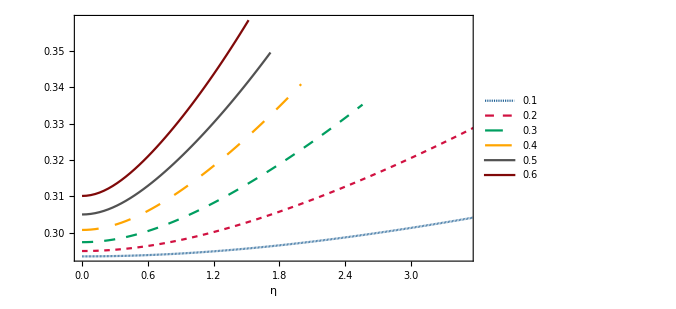

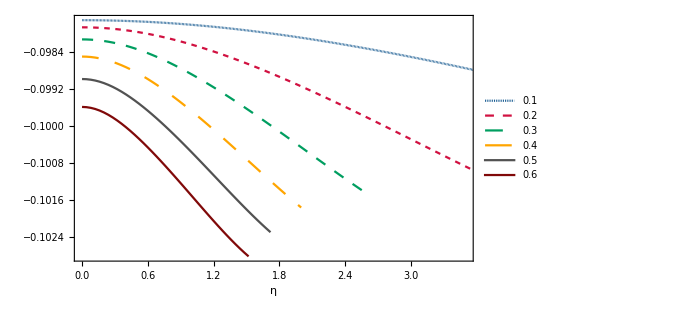

```mathematica
ListLinePlot[{Re[Ts0[[1]]],Re[Ts0[[2]]],Re[Ts0[[3]]],Re[Ts0[[4]]],Re[Ts0[[5]]],Re[Ts0[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.1,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[Ts0[[1]]],Im[Ts0[[2]]],Im[Ts0[[3]]],Im[Ts0[[4]]],Im[Ts0[[5]]],Im[Ts0[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 14,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 14,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 14,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 14,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 14,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 14,FontFamily->"Times New Roman"]},{0.1,0.25}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
(Max[Re[Tsd0[[1]]]]-Min[Re[Tsd0[[1]]]])/Min[Re[Tsd0[[1]]]]*100
(Max[Im[Tsd0[[1]]]]-Min[Im[Tsd0[[1]]]])/Min[Im[Tsd0[[1]]]]*100
(Max[Re[Tsd0[[6]]]]-Min[Re[Tsd0[[6]]]])/Min[Re[Tsd0[[6]]]]*100
(Max[Im[Tsd0[[6]]]]-Min[Im[Tsd0[[6]]]])/Min[Im[Tsd0[[6]]]]*100
```

11.5443

-3.11795

15.6302

-3.14147

#### L=2

```mathematica
Ts0={{{0,0.48445303881178275-0.09681140856710949 ⅈ},{1/25+ⅈ/25,0.4844556609921567-0.09681157677416678 ⅈ},{2/25+(2 ⅈ)/25,0.4844635244739888-0.0968120812144657 ⅈ},{3/25+(3 ⅈ)/25,0.48447662007190967-0.09681292134478345 ⅈ},{4/25+(4 ⅈ)/25,0.48449493254342896-0.09681409626374608 ⅈ},{1/5+ⅈ/5,0.4845184406785456-0.0968156047171473 ⅈ},{6/25+(6 ⅈ)/25,0.48454711742705425-0.09681744510554409 ⅈ},{7/25+(7 ⅈ)/25,0.48458093005918557-0.0968196154938427 ⅈ},{8/25+(8 ⅈ)/25,0.48461984035739086-0.09682211362275042 ⅈ},{9/25+(9 ⅈ)/25,0.4846638048367288-0.09682493692193975 ⅈ},{2/5+(2 ⅈ)/5,0.4847127749909801-0.09682808252476531 ⅈ},{11/25+(11 ⅈ)/25,0.484766697561377-0.09683154728434165 ⅈ},{12/25+(12 ⅈ)/25,0.48482551482465724-0.09683532779079455 ⅈ},{13/25+(13 ⅈ)/25,0.4848891648970299-0.09683942038948339 ⅈ},{14/25+(14 ⅈ)/25,0.4849575820506075-0.09684382119999055 ⅈ},{3/5+(3 ⅈ)/5,0.4850306970388762-0.09684852613567471 ⅈ},{16/25+(16 ⅈ)/25,0.4851084374278508-0.09685353092359042 ⅈ},{17/25+(17 ⅈ)/25,0.4851907279297062-0.09685883112457899 ⅈ},{18/25+(18 ⅈ)/25,0.4852774907358423-0.09686442215335497 ⅈ},{19/25+(19 ⅈ)/25,0.4853686458465701-0.09687029929841097 ⅈ},{4/5+(4 ⅈ)/5,0.4854641113948448-0.09687645774159255 ⅈ},{21/25+(21 ⅈ)/25,0.48556380396174276-0.09688289257719791 ⅈ},{22/25+(22 ⅈ)/25,0.48566763888166675-0.09688959883048304 ⅈ},{23/25+(23 ⅈ)/25,0.48577553053554245-0.09689657147546196 ⅈ},{24/25+(24 ⅈ)/25,0.485887392630569-0.09690380545191388 ⅈ},{1+ⅈ,0.4860031384653609-0.0969112956815252 ⅈ},{26/25+(26 ⅈ)/25,0.48612268117959173-0.09691903708310415 ⅈ},{27/25+(27 ⅈ)/25,0.4862459339874955-0.09692702458683962 ⅈ},{28/25+(28 ⅈ)/25,0.48637281039486596-0.09693525314754592 ⅈ},{29/25+(29 ⅈ)/25,0.48650322439930666-0.09694371775692597 ⅈ},{6/5+(6 ⅈ)/5,0.48663709067381283-0.09695241345480383 ⅈ},{31/25+(31 ⅈ)/25,0.48677432473382554-0.09696133533936213 ⅈ},{32/25+(32 ⅈ)/25,0.4869148430881092-0.0969704785763916 ⅈ},{33/25+(33 ⅈ)/25,0.48705856337390263-0.09697983840757979 ⅈ},{34/25+(34 ⅈ)/25,0.48720540447691074-0.09698941015786935 ⅈ},{7/5+(7 ⅈ)/5,0.4873552866367781-0.096999189241923 ⅈ},{36/25+(36 ⅈ)/25,0.4875081315387561-0.09700917116973583 ⅈ},{37/25+(37 ⅈ)/25,0.48766386239232346-0.09701935155144083 ⅈ},{38/25+(38 ⅈ)/25,0.4878224039975434-0.09702972610135129 ⅈ},{39/25+(39 ⅈ)/25,0.4879836827999709-0.09704029064129104 ⅈ},{8/5+(8 ⅈ)/5,0.48814762693491826-0.0970510411032583 ⅈ},{41/25+(41 ⅈ)/25,0.4883141662618911-0.09706197353147408 ⅈ},{42/25+(42 ⅈ)/25,0.48848323238998664-0.09707308408386159 ⅈ},{43/25+(43 ⅈ)/25,0.48865475869503316-0.09708436903300463 ⅈ},{44/25+(44 ⅈ)/25,0.48882868032921795-0.09709582476662963 ⅈ},{9/5+(9 ⅈ)/5,0.4890049342239216-0.09710744778765794 ⅈ},{46/25+(46 ⅈ)/25,0.4891834590864444-0.09711923471386559 ⅈ},{47/25+(47 ⅈ)/25,0.4893641953912727-0.09713118227719612 ⅈ},{48/25+(48 ⅈ)/25,0.4895470853664945-0.09714328732276085 ⅈ},{49/25+(49 ⅈ)/25,0.48973207297593596-0.09715554680756243 ⅈ},{2+2 ⅈ,0.4899191038975505-0.09716795779897604 ⅈ},{51/25+(51 ⅈ)/25,0.4901081254985548-0.09718051747301887 ⅈ},{52/25+(52 ⅈ)/25,0.49029908680776507-0.09719322311243513 ⅈ},{53/25+(53 ⅈ)/25,0.49049193848555483-0.09720607210462612 ⅈ},{54/25+(54 ⅈ)/25,0.4906866327918164-0.0972190619394454 ⅈ},{11/5+(11 ⅈ)/5,0.4908831235522725-0.09723219020688467 ⅈ},{56/25+(56 ⅈ)/25,0.4910813661234608-0.09724545459467006 ⅈ},{57/25+(57 ⅈ)/25,0.49128131735667085-0.09725885288578517 ⅈ},{58/25+(58 ⅈ)/25,0.491482935561098-0.09727238295593976 ⅈ},{59/25+(59 ⅈ)/25,0.491686180466441-0.09728604277099849 ⅈ},{12/5+(12 ⅈ)/5,0.491891013185151-0.09729983038438099 ⅈ},{61/25+(61 ⅈ)/25,0.49209739617451664-0.09731374393444907 ⅈ},{62/25+(62 ⅈ)/25,0.49230529319874566-0.09732778164188788 ⅈ},{63/25+(63 ⅈ)/25,0.49251466929118604-0.09734194180709285 ⅈ},{64/25+(64 ⅈ)/25,0.49272549071681176-0.09735622280756927 ⅈ},{13/5+(13 ⅈ)/5,0.49293772493508126-0.0973706230953532 ⅈ},{66/25+(66 ⅈ)/25,0.4931513405632618-0.0973851411944572 ⅈ},{67/25+(67 ⅈ)/25,0.49336630734030007-0.09739977569834994 ⅈ},{68/25+(68 ⅈ)/25,0.49358259609130617-0.09741452526747134 ⅈ},{69/25+(69 ⅈ)/25,0.49380017869270776-0.09742938862678792 ⅈ},{14/5+(14 ⅈ)/5,0.4940190280381229-0.09744436456339316 ⅈ},{71/25+(71 ⅈ)/25,0.49423911800498443-0.09745945192415248 ⅈ},{72/25+(72 ⅈ)/25,0.4944604234219531-0.09747464961339751 ⅈ},{73/25+(73 ⅈ)/25,0.49468292003713593-0.09748995659067168 ⅈ},{74/25+(74 ⅈ)/25,0.49490658448713-0.09750537186852479 ⅈ},{3+3 ⅈ,0.49513139426690095-0.09752089451036203 ⅈ},{76/25+(76 ⅈ)/25,0.49535732770050406-0.097536523628345 ⅈ},{77/25+(77 ⅈ)/25,0.49558436391264854-0.09755225838134687 ⅈ},{78/25+(78 ⅈ)/25,0.4958124828011031-0.09756809797295889 ⅈ},{79/25+(79 ⅈ)/25,0.49604166500993996-0.09758404164955288 ⅈ},{16/5+(16 ⅈ)/5,0.4962718919036056-0.09760008869839394 ⅈ},{81/25+(81 ⅈ)/25,0.49650314554181246-0.09761623844580694 ⅈ},{82/25+(82 ⅈ)/25,0.4967354086552364-0.09763249025539442 ⅈ},{83/25+(83 ⅈ)/25,0.49696866462200673-0.09764884352630514 ⅈ},{84/25+(84 ⅈ)/25,0.4972028974449737-0.09766529769155245 ⅈ},{17/5+(17 ⅈ)/5,0.4974380917297381-0.09768185221638262 ⅈ},{86/25+(86 ⅈ)/25,0.4976742326634224-0.09769850659669006 ⅈ},{87/25+(87 ⅈ)/25,0.49791130599416855-0.09771526035748045 ⅈ},{88/25+(88 ⅈ)/25,0.49814929801134217-0.09773211305137978 ⅈ},{89/25+(89 ⅈ)/25,0.4983881955264243-0.09774906425718677 ⅈ},{18/5+(18 ⅈ)/5,0.49862798585457097-0.09776611357847126 ⅈ},{91/25+(91 ⅈ)/25,0.498868656796821-0.09778326064221313 ⅈ},{92/25+(92 ⅈ)/25,0.499110196622934-0.09780050509748235 ⅈ},{93/25+(93 ⅈ)/25,0.4993525940548369-0.09781784661416129 ⅈ},{94/25+(94 ⅈ)/25,0.4995958382506608-0.0978352848817032 ⅈ},{19/5+(19 ⅈ)/5,0.49983991878934825-0.09785281960793012 ⅈ},{96/25+(96 ⅈ)/25,0.5000848256558134-0.09787045051786707 ⅈ},{97/25+(97 ⅈ)/25,0.5003305492266351-0.09788817735261122 ⅈ},{98/25+(98 ⅈ)/25,0.5005770802562639-0.0979059998682355 ⅈ},{99/25+(99 ⅈ)/25,0.5008244098637278-0.09792391783472637 ⅈ},{4+4 ⅈ,0.501072529519816-0.09794193103495218 ⅈ},{101/25+(101 ⅈ)/25,0.5013214310347258-0.09796003926366387 ⅈ},{102/25+(102 ⅈ)/25,0.5015711065461551-0.09797824232652551 ⅈ},{103/25+(103 ⅈ)/25,0.5018215485078236-0.09799654003917335 ⅈ},{104/25+(104 ⅈ)/25,0.5020727496784089-0.09801493222630403 ⅈ},{21/5+(21 ⅈ)/5,0.502324703110879-0.09803341872078934 ⅈ},{106/25+(106 ⅈ)/25,0.5025774021422104-0.09805199936281679 ⅈ},{107/25+(107 ⅈ)/25,0.5028308403834735-0.09807067399905747 ⅈ},{108/25+(108 ⅈ)/25,0.5030850117102738-0.09808944248185616 ⅈ},{109/25+(109 ⅈ)/25,0.5033399102535349-0.09810830466844736 ⅈ},{22/5+(22 ⅈ)/5,0.5035955303906092-0.09812726042019283 ⅈ},{111/25+(111 ⅈ)/25,0.5038518667367063-0.09814630960184187 ⅈ},{112/25+(112 ⅈ)/25,0.5041089141366225-0.09816545208081359 ⅈ},{113/25+(113 ⅈ)/25,0.5043666676567651-0.09818468772649953 ⅈ},{114/25+(114 ⅈ)/25,0.5046251225774568-0.09820401640958627 ⅈ},{23/5+(23 ⅈ)/5,0.5048842743855091-0.09822343800139803 ⅈ},{116/25+(116 ⅈ)/25,0.5051441187670556-0.09824295237325786 ⅈ},{117/25+(117 ⅈ)/25,0.5054046516006357-0.09826255939586778 ⅈ},{118/25+(118 ⅈ)/25,0.5056658689505171-0.09828225893870496 ⅈ},{119/25+(119 ⅈ)/25,0.5059277670602481-0.09830205086943782 ⅈ},{24/5+(24 ⅈ)/5,0.506190342346432-0.09832193505335553 ⅈ},{121/25+(121 ⅈ)/25,0.5064535913927151-0.09834191135281693 ⅈ},{122/25+(122 ⅈ)/25,0.5067175109439762-0.09836197962671345 ⅈ},{123/25+(123 ⅈ)/25,0.5069820979007161-0.09838213972994611 ⅈ},{124/25+(124 ⅈ)/25,0.5072473493136331-0.09840239151292078 ⅈ},{5+5 ⅈ,0.5075132623783809-0.09842273482105414 ⅈ},{126/25+(126 ⅈ)/25,0.5077798344305007-0.0984431694942966 ⅈ},{127/25+(127 ⅈ)/25,0.508047062940521-0.09846369536666638 ⅈ},{128/25+(128 ⅈ)/25,0.5083149455092176-0.0984843122657996 ⅈ},{129/25+(129 ⅈ)/25,0.5085834798630292-0.09850502001251028 ⅈ},{26/5+(26 ⅈ)/5,0.5088526638496205-0.09852581842036601 ⅈ},{131/25+(131 ⅈ)/25,0.5091224954335897-0.09854670729527343 ⅈ},{132/25+(132 ⅈ)/25,0.5093929726923117-0.0985676864350776 ⅈ},{133/25+(133 ⅈ)/25,0.5096640938119145-0.0985887556291717 ⅈ},{134/25+(134 ⅈ)/25,0.5099358570833815-0.0986099146581193 ⅈ},{27/5+(27 ⅈ)/5,0.5102082608987768-0.09863116329328765 ⅈ},{136/25+(136 ⅈ)/25,0.5104813037475872-0.0986525012964915 ⅈ},{137/25+(137 ⅈ)/25,0.5107549842131764-0.09867392841964844 ⅈ},{138/25+(138 ⅈ)/25,0.5110293009693493-0.09869544440444405 ⅈ},{139/25+(139 ⅈ)/25,0.5113042527770186-0.09871704898200864 ⅈ},{28/5+(28 ⅈ)/5,0.5115798384809734-0.09873874187260252 ⅈ},{141/25+(141 ⅈ)/25,0.5118560570067433-0.09876052278531339 ⅈ},{142/25+(142 ⅈ)/25,0.5121329073575547-0.0987823914177615 ⅈ},{143/25+(143 ⅈ)/25,0.5124103886113787-0.09880434745581643 ⅈ},{144/25+(144 ⅈ)/25,0.5126884999180623-0.09882639057332174 ⅈ},{29/5+(29 ⅈ)/5,0.512967240496544-0.09884852043183072 ⅈ},{146/25+(146 ⅈ)/25,0.513246609632148-0.09887073668035024 ⅈ},{147/25+(147 ⅈ)/25,0.5135266066739558-0.09889303895509431 ⅈ},{148/25+(148 ⅈ)/25,0.5138072310322508-0.09891542687924643 ⅈ},{149/25+(149 ⅈ)/25,0.5140884821760348-0.09893790006273179 ⅈ},{6+6 ⅈ,0.5143703596306116-0.09896045810199702 ⅈ},{151/25+(151 ⅈ)/25,0.5146528629752379-0.09898310057979975 ⅈ},{152/25+(152 ⅈ)/25,0.5149359918408367-0.09900582706500699 ⅈ},{153/25+(153 ⅈ)/25,0.5152197459077718-0.0990286371124008 ⅈ},{154/25+(154 ⅈ)/25,0.515504124903682-0.09905153026249429 ⅈ},{31/5+(31 ⅈ)/5,0.515789128601372-0.09907450604135522 ⅈ},{156/25+(156 ⅈ)/25,0.5160747568167567-0.09909756396043772 ⅈ},{157/25+(157 ⅈ)/25,0.5163610094068598-0.09912070351642302 ⅈ},{158/25+(158 ⅈ)/25,0.5166478862678632-0.0991439241910684 ⅈ},{159/25+(159 ⅈ)/25,0.5169353873332045-0.09916722545106402 ⅈ},{32/5+(32 ⅈ)/5,0.517223512571723-0.09919060674789876 ⅈ},{161/25+(161 ⅈ)/25,0.5175122619858507-0.09921406751773273 ⅈ},{162/25+(162 ⅈ)/25,0.5178016356098479-0.09923760718128014 ⅈ},{163/25+(163 ⅈ)/25,0.5180916335080816-0.09926122514369834 ⅈ},{164/25+(164 ⅈ)/25,0.5183822557733447-0.0992849207944859 ⅈ},{33/5+(33 ⅈ)/5,0.5186735025252147-0.0993086935073885 ⅈ},{166/25+(166 ⅈ)/25,0.5189653739084522-0.09933254264031274 ⅈ},{167/25+(167 ⅈ)/25,0.5192578700914351-0.09935646753524871 ⅈ},{168/25+(168 ⅈ)/25,0.5195509912646298-0.09938046751819876 ⅈ},{169/25+(169 ⅈ)/25,0.5198447376390966-0.09940454189911657 ⅈ},{34/5+(34 ⅈ)/5,0.5201391094450291-0.09942868997185211 ⅈ},{171/25+(171 ⅈ)/25,0.5204341069303265-0.09945291101410574 ⅈ},{172/25+(172 ⅈ)/25,0.5207297303591972-0.09947720428738967 ⅈ},{173/25+(173 ⅈ)/25,0.5210259800107919-0.09950156903699761 ⅈ},{174/25+(174 ⅈ)/25,0.5213228561778691-0.09952600449198183 ⅈ},{7+7 ⅈ,0.5216203591654864-0.0995505098651387 ⅈ},{176/25+(176 ⅈ)/25,0.521918489289722-0.09957508435300141 ⅈ},{177/25+(177 ⅈ)/25,0.5222172468764215-0.09959972713584075 ⅈ},{178/25+(178 ⅈ)/25,0.5225166322599724-0.09962443737767403 ⅈ}},{{0,0.4868708565362278-0.0969702594387445 ⅈ},{1/25+ⅈ/25,0.48688172484421743-0.09697093265706319 ⅈ},{2/25+(2 ⅈ)/25,0.4869142740246042-0.0969729491660263 ⅈ},{3/25+(3 ⅈ)/25,0.4869683382191642-0.09697629960312164 ⅈ},{4/25+(4 ⅈ)/25,0.48704364586293425-0.0969809686345221 ⅈ},{1/5+ⅈ/5,0.4871398266382638-0.09698693534206222 ⅈ},{6/25+(6 ⅈ)/25,0.48725642064715013-0.09699417373521894 ⅈ},{7/25+(7 ⅈ)/25,0.4873928892849235-0.09700265336033326 ⅈ},{8/25+(8 ⅈ)/25,0.48754862725515824-0.09701233997685445 ⅈ},{9/25+(9 ⅈ)/25,0.4877229751598827-0.09702319626973202 ⅈ},{2/5+(2 ⅈ)/5,0.48791523213589194-0.09703518256870328 ⅈ},{11/25+(11 ⅈ)/25,0.48812466807731075-0.09704825754862091 ⅈ},{12/25+(12 ⅈ)/25,0.4883505350745992-0.09706237888956351 ⅈ},{13/25+(13 ⅈ)/25,0.4885920777990563-0.09707750388066747 ⅈ},{14/25+(14 ⅈ)/25,0.48884854265932853-0.09709358995686446 ⅈ},{3/5+(3 ⅈ)/5,0.4891191856447838-0.09711059516258568 ⅈ},{16/25+(16 ⅈ)/25,0.4894032788449996-0.09712847854070537 ⅈ},{17/25+(17 ⅈ)/25,0.48970011569281785-0.09714720044839353 ⅈ},{18/25+(18 ⅈ)/25,0.49000901502032024-0.09716672280409507 ⅈ},{19/25+(19 ⅈ)/25,0.49032932404405327-0.09718700927157654 ⅈ},{4/5+(4 ⅈ)/5,0.49066042041012303-0.09720802538800921 ⅈ},{21/25+(21 ⅈ)/25,0.4910017134340046-0.09722973864348651 ⅈ},{22/25+(22 ⅈ)/25,0.49135264466666295-0.09725211851936452 ⅈ},{23/25+(23 ⅈ)/25,0.491712687910217-0.09727513649247217 ⅈ},{24/25+(24 ⅈ)/25,0.4920813487948578-0.09729876601169189 ⅈ},{1+ⅈ,0.4924581640156392-0.09732298245273557 ⅈ},{26/25+(26 ⅈ)/25,0.49284270031421384-0.0973477630562166 ⅈ},{27/25+(27 ⅈ)/25,0.49323455327743626-0.09737308685338425 ⅈ},{28/25+(28 ⅈ)/25,0.4936333460125348-0.09739893458322921 ⅈ},{29/25+(29 ⅈ)/25,0.4940387277474213-0.09742528860395397 ⅈ},{6/5+(6 ⅈ)/5,0.49445037239509115-0.09745213280132926 ⅈ},{31/25+(31 ⅈ)/25,0.49486797711260333-0.09747945249587793 ⅈ},{32/25+(32 ⅈ)/25,0.4952912608780923-0.09750723435043994 ⅈ},{33/25+(33 ⅈ)/25,0.49571996310334787-0.09753546627929532 ⅈ},{34/25+(34 ⅈ)/25,0.49615384229466125-0.09756413735972454 ⅈ},{7/5+(7 ⅈ)/5,0.4965926747707161-0.09759323774663614 ⅈ},{36/25+(36 ⅈ)/25,0.49703625344317887-0.09762275859069208 ⅈ},{37/25+(37 ⅈ)/25,0.4974843866631752-0.09765269196020243 ⅈ},{38/25+(38 ⅈ)/25,0.4979368971349447-0.09768303076692991 ⅈ},{39/25+(39 ⅈ)/25,0.49839362089650446-0.09771376869585588 ⅈ},{8/5+(8 ⅈ)/5,0.4988544063660797-0.09774490013887605 ⅈ},{41/25+(41 ⅈ)/25,0.4993191134522755-0.0977764201323442 ⅈ},{42/25+(42 ⅈ)/25,0.4997876127254184-0.09780832429834299 ⅈ},{43/25+(43 ⅈ)/25,0.5002597846471402-0.09784060878952805 ⅈ},{44/25+(44 ⅈ)/25,0.5007355188550563-0.09787327023738068 ⅈ},{9/5+(9 ⅈ)/5,0.5012147134993-0.09790630570368687 ⅈ},{46/25+(46 ⅈ)/25,0.5016972746276417-0.09793971263506324 ⅈ},{47/25+(47 ⅈ)/25,0.5021831156159775-0.09797348882034243 ⅈ},{48/25+(48 ⅈ)/25,0.5026721566410535-0.09800763235064168 ⅈ},{49/25+(49 ⅈ)/25,0.5031643241924154-0.09804214158193542 ⅈ},{2+2 ⅈ,0.5036595506207124-0.09807701509996831 ⅈ},{51/25+(51 ⅈ)/25,0.5041577737196399-0.09811225168734677 ⅈ},{52/25+(52 ⅈ)/25,0.5046589363389634-0.09814785029265925 ⅈ},{53/25+(53 ⅈ)/25,0.5051629860262327-0.09818381000148477 ⅈ},{54/25+(54 ⅈ)/25,0.5056698746949477-0.09822013000915576 ⅈ},{11/5+(11 ⅈ)/5,0.5061795583171056-0.09825680959515738 ⅈ},{56/25+(56 ⅈ)/25,0.5066919966381962-0.09829384809904326 ⅈ},{57/25+(57 ⅈ)/25,0.507207152912867-0.09833124489777038 ⅈ},{58/25+(58 ⅈ)/25,0.5077249936596103-0.09836899938435158 ⅈ},{59/25+(59 ⅈ)/25,0.5082454884329517-0.09840711094773877 ⅈ},{12/5+(12 ⅈ)/5,0.5087686096117413-0.098445578953859 ⅈ},{61/25+(61 ⅈ)/25,0.5092943322022615-0.09848440272772481 ⅈ},{62/25+(62 ⅈ)/25,0.5098226336549637-0.0985235815365561 ⅈ},{63/25+(63 ⅈ)/25,0.5103534936937492-0.09856311457385059 ⅈ},{64/25+(64 ⅈ)/25,0.5108868941567917-0.0986030009443471 ⅈ},{13/5+(13 ⅈ)/5,0.5114228188479863-0.09864323964983403 ⅈ},{66/25+(66 ⅈ)/25,0.511961253398182-0.09868382957575486 ⅈ},{67/25+(67 ⅈ)/25,0.5125021851354236-0.09872476947857374 ⅈ},{68/25+(68 ⅈ)/25,0.5130456029634967-0.0987660579738612 ⅈ},{69/25+(69 ⅈ)/25,0.5135914972481233-0.09880769352507043 ⅈ},{14/5+(14 ⅈ)/5,0.5141398597102128-0.0988496744329731 ⅈ},{71/25+(71 ⅈ)/25,0.5146906833256204-0.09889199882573042 ⅈ},{72/25+(72 ⅈ)/25,0.5152439622309111-0.09893466464957493 ⅈ},{73/25+(73 ⅈ)/25,0.5157996916346702-0.09897766966008485 ⅈ},{74/25+(74 ⅈ)/25,0.5163578677339361-0.09902101141403173 ⅈ},{3+3 ⅈ,0.5169184876353695-0.09906468726178651 ⅈ},{76/25+(76 ⅈ)/25,0.5174815492808029-0.09910869434027017 ⅈ},{77/25+(77 ⅈ)/25,0.5180470513768447-0.09915302956643884 ⅈ},{78/25+(78 ⅈ)/25,0.5186149933282387-0.0991976896312904 ⅈ},{79/25+(79 ⅈ)/25,0.5191853751747062-0.09924267099438742 ⅈ},{16/5+(16 ⅈ)/5,0.5197581975310163-0.0992879698788869 ⅈ},{81/25+(81 ⅈ)/25,0.5203334615300561-0.09933358226707163 ⅈ},{82/25+(82 ⅈ)/25,0.5209111687686889-0.09937950389637788 ⅈ},{83/25+(83 ⅈ)/25,0.5214913212562068-0.09942573025591603 ⅈ},{84/25+(84 ⅈ)/25,0.5220739213651983-0.09947225658347894 ⅈ},{17/5+(17 ⅈ)/5,0.5226589717846705-0.09951907786303744 ⅈ},{86/25+(86 ⅈ)/25,0.523246475475277-0.0995661888227193 ⅈ},{87/25+(87 ⅈ)/25,0.5238364356265123-0.09961358393326987 ⅈ},{88/25+(88 ⅈ)/25,0.5244288556157517-0.09966125740699389 ⅈ},{89/25+(89 ⅈ)/25,0.5250237389690218-0.09970920319717547 ⅈ},{18/5+(18 ⅈ)/5,0.5256210893233955-0.09975741499797658 ⅈ},{91/25+(91 ⅈ)/25,0.5262209103909198-0.09980588624481222 ⅈ}},{{0,0.49086856785282207-0.0972379534086026 ⅈ},{1/25+ⅈ/25,0.49089458143303405-0.0972394674684291 ⅈ},{2/25+(2 ⅈ)/25,0.4909722709606014-0.09724399163333795 ⅈ},{3/25+(3 ⅈ)/25,0.4911006067241031-0.09725147299665503 ⅈ},{4/25+(4 ⅈ)/25,0.49127794944666336-0.09726182706344215 ⅈ},{1/5+ⅈ/5,0.4915021534076297-0.09727494274650553 ⅈ},{6/25+(6 ⅈ)/25,0.4917706897940399-0.09729068844089848 ⅈ},{7/25+(7 ⅈ)/25,0.4920807754878416-0.09730891849944164 ⅈ},{8/25+(8 ⅈ)/25,0.4924294946713952-0.09732947950110661 ⅈ},{9/25+(9 ⅈ)/25,0.4928139044177987-0.0973522158526062 ⅈ},{2/5+(2 ⅈ)/5,0.4932311195950038-0.09737697444373085 ⅈ},{11/25+(11 ⅈ)/25,0.4936783760118372-0.09740360824683739 ⅈ},{12/25+(12 ⅈ)/25,0.49415307330012165-0.09743197888398612 ⅈ},{13/25+(13 ⅈ)/25,0.4946528004999128-0.0974619582726103 ⅈ},{14/25+(14 ⅈ)/25,0.49517534788414314-0.09749342950512262 ⅈ},{3/5+(3 ⅈ)/5,0.49571870850578426-0.09752628712954317 ⅈ},{16/25+(16 ⅈ)/25,0.49628107254273-0.09756043698832355 ⅈ},{17/25+(17 ⅈ)/25,0.4968608169579541-0.09759579575105386 ⅈ},{18/25+(18 ⅈ)/25,0.4974564924186151-0.0976322902509922 ⅈ},{19/25+(19 ⅈ)/25,0.49806680890095245-0.09766985671002036 ⅈ},{4/5+(4 ⅈ)/5,0.49869062097905614-0.09770843991419748 ⅈ},{21/25+(21 ⅈ)/25,0.49932691345987973-0.0977479923835577 ⅈ},{22/25+(22 ⅈ)/25,0.4999747877756993-0.09778847356525959 ⅈ},{23/25+(23 ⅈ)/25,0.5006334493644585-0.0978298490682386 ⅈ},{24/25+(24 ⅈ)/25,0.5013021961430743-0.09787208994956285 ⅈ},{1+ⅈ,0.5019804080951897-0.09791517205710296 ⅈ},{26/25+(26 ⅈ)/25,0.5026675379417227-0.0979590754293612 ⅈ},{27/25+(27 ⅈ)/25,0.5033631028309713-0.09800378375086197 ⅈ},{28/25+(28 ⅈ)/25,0.5040666769682685-0.09804928386003586 ⅈ},{29/25+(29 ⅈ)/25,0.5047778850983053-0.09809556530572763 ⅈ},{6/5+(6 ⅈ)/5,0.5054963967527201-0.09814261994810423 ⅈ},{31/25+(31 ⅈ)/25,0.5062219211789393-0.09819044159970511 ⅈ},{32/25+(32 ⅈ)/25,0.5069542028718581-0.09823902570251183 ⅈ},{33/25+(33 ⅈ)/25,0.5076930176366357-0.09828836903717371 ⅈ},{34/25+(34 ⅈ)/25,0.5084381691179447-0.09833846946084053 ⅈ},{7/5+(7 ⅈ)/5,0.509189485737977-0.09838932567038955 ⅈ},{36/25+(36 ⅈ)/25,0.5099468179921196-0.0984409369881778 ⅈ},{37/25+(37 ⅈ)/25,0.5107100360573172-0.09849330316777029 ⅈ},{38/25+(38 ⅈ)/25,0.511479027673677-0.09854642421740613 ⅈ},{39/25+(39 ⅈ)/25,0.5122536962648292-0.09860030023924281 ⅈ},{8/5+(8 ⅈ)/5,0.513033959266952-0.09865493128267241 ⅈ},{41/25+(41 ⅈ)/25,0.5138197466402495-0.09871031721023138 ⅈ},{42/25+(42 ⅈ)/25,0.5146109995400564-0.09876645757483121 ⅈ},{43/25+(43 ⅈ)/25,0.5154076691277119-0.09882335150721297 ⅈ},{44/25+(44 ⅈ)/25,0.5162097155039278-0.09888099761269062 ⅈ},{9/5+(9 ⅈ)/5,0.5170171067496105-0.09893939387638588 ⅈ},{46/25+(46 ⅈ)/25,0.5178298180610511-0.09899853757627998 ⅈ},{47/25+(47 ⅈ)/25,0.5186478309680866-0.09905842520351282 ⅈ},{48/25+(48 ⅈ)/25,0.5194711326252968-0.09911905238945737 ⅈ},{49/25+(49 ⅈ)/25,0.520299715167579-0.09918041383917327 ⅈ},{2+2 ⅈ,0.5211335751225459-0.09924250327091728 ⅈ},{51/25+(51 ⅈ)/25,0.5219727128731486-0.09930531336144918 ⅈ},{52/25+(52 ⅈ)/25,0.52281713216477-0.09936883569692191 ⅈ},{53/25+(53 ⅈ)/25,0.52366683965175-0.09943306072919189 ⅈ},{54/25+(54 ⅈ)/25,0.524521844478952-0.09949797773742355 ⅈ},{11/5+(11 ⅈ)/5,0.5253821578945186-0.09956357479489364 ⅈ},{56/25+(56 ⅈ)/25,0.5262477928904653-0.09962983874092679 ⅈ},{57/25+(57 ⅈ)/25,0.5271187638681714-0.0996967551579172 ⅈ},{58/25+(58 ⅈ)/25,0.5279950863262108-0.0997643083534091 ⅈ},{59/25+(59 ⅈ)/25,0.5288767765682855-0.09983248134721733 ⅈ},{12/5+(12 ⅈ)/5,0.5297638514293168-0.09990125586358435 ⅈ},{61/25+(61 ⅈ)/25,0.5306563280180031-0.09997061232837033 ⅈ},{62/25+(62 ⅈ)/25,0.5315542234743761-0.1000405298712806 ⅈ},{63/25+(63 ⅈ)/25,0.5324575547410852-0.10011098633312646 ⅈ},{64/25+(64 ⅈ)/25,0.5333663383473186-0.10018195827811974 ⅈ}},{{0,0.49639919666778876-0.0976181257175579 ⅈ},{1/25+ⅈ/25,0.49644992961130147-0.09762079968288427 ⅈ},{2/25+(2 ⅈ)/25,0.4966006029847065-0.09762875677562674 ⅈ},{3/25+(3 ⅈ)/25,0.4968468677469958-0.09764181035537592 ⅈ},{4/25+(4 ⅈ)/25,0.4971821603909829-0.0976596734598008 ⅈ},{1/5+ⅈ/5,0.49759850978410297-0.09768198903764364 ⅈ},{6/25+(6 ⅈ)/25,0.49808734113242975-0.09770836263312256 ⅈ},{7/25+(7 ⅈ)/25,0.498640134393426-0.09773839196593426 ⅈ},{8/25+(8 ⅈ)/25,0.49924887853360705-0.09777168996046165 ⅈ},{9/25+(9 ⅈ)/25,0.499906329891167-0.0978079001404086 ⅈ},{2/5+(2 ⅈ)/5,0.5006061173278058-0.09784670506498967 ⅈ},{11/25+(11 ⅈ)/25,0.5013427443882965-0.09788782936247072 ⅈ},{12/25+(12 ⅈ)/25,0.5021115315220928-0.09793103908037551 ⅈ},{13/25+(13 ⅈ)/25,0.5029085295153694-0.0979761388316533 ⅈ},{14/25+(14 ⅈ)/25,0.5037304240847742-0.09802296783576316 ⅈ},{3/5+(3 ⅈ)/5,0.5045744430675436-0.09807139558692211 ⅈ},{16/25+(16 ⅈ)/25,0.5054382719233652-0.09812131759140616 ⅈ},{17/25+(17 ⅈ)/25,0.5063199797615565-0.09817265141130273 ⅈ},{18/25+(18 ⅈ)/25,0.5072179561394105-0.09822533311991924 ⅈ},{19/25+(19 ⅈ)/25,0.5081308578819407-0.09827931419485841 ⅈ},{4/5+(4 ⅈ)/5,0.5090575647524768-0.09833455883117669 ⅈ},{21/25+(21 ⅈ)/25,0.5099971427006161-0.09839104163587188 ⅈ},{22/25+(22 ⅈ)/25,0.5109488134726877-0.09844874565707981 ⅈ},{23/25+(23 ⅈ)/25,0.5119119295000055-0.0985076607009019 ⅈ},{24/25+(24 ⅈ)/25,0.5128859531324799-0.09856778189210837 ⅈ},{1+ⅈ,0.5138704394344976-0.098629108439911 ⅈ},{26/25+(26 ⅈ)/25,0.5148650218949348-0.09869164257538862 ⅈ},{27/25+(27 ⅈ)/25,0.5158694005197227-0.09875538863233597 ⅈ},{28/25+(28 ⅈ)/25,0.5168833318733826-0.09882035224799983 ⅈ},{29/25+(29 ⅈ)/25,0.51790662071689-0.09888653966428348 ⅈ},{6/5+(6 ⅈ)/5,0.518939112955459-0.09895395711348887 ⅈ},{31/25+(31 ⅈ)/25,0.5199806896635791-0.0990226102756299 ⅈ},{32/25+(32 ⅈ)/25,0.5210312619981455-0.0990925037968021 ⅈ},{33/25+(33 ⅈ)/25,0.5220907668456518-0.09916364086013932 ⅈ},{34/25+(34 ⅈ)/25,0.5231591630777742-0.0992360228025729 ⅈ},{7/5+(7 ⅈ)/5,0.5242364283125784-0.09930964877199971 ⅈ},{36/25+(36 ⅈ)/25,0.5253225560971216-0.09938451542061183 ⅈ},{37/25+(37 ⅈ)/25,0.526417553442237-0.09946061663108308 ⅈ},{38/25+(38 ⅈ)/25,0.5275214386525052-0.09953794327308375 ⅈ},{39/25+(39 ⅈ)/25,0.5286342394043724-0.0996164829882299 ⅈ},{8/5+(8 ⅈ)/5,0.5297559910335129-0.09969622000209376 ⅈ},{41/25+(41 ⅈ)/25,0.5308867349992248-0.09977713496232422 ⅈ},{42/25+(42 ⅈ)/25,0.5320265174991472-0.09985920480226432 ⅈ},{43/25+(43 ⅈ)/25,0.5331753882121476-0.09994240262972137 ⅈ},{44/25+(44 ⅈ)/25,0.534333399151011-0.10002669764075066 ⅈ},{9/5+(9 ⅈ)/5,0.5355006036097156-0.10011205505846692 ⅈ},{46/25+(46 ⅈ)/25,0.5366770551927237-0.1001984360969982 ⅈ},{47/25+(47 ⅈ)/25,0.5378628069159301-0.10028579795075987 ⅈ},{48/25+(48 ⅈ)/25,0.5390579103707925-0.10037409380924361 ⅈ},{49/25+(49 ⅈ)/25,0.5402624149447374-0.10046327289750334 ⅈ},{2+2 ⅈ,0.5414763670922834-0.1005532805424683 ⅈ}},{{0,0.5033989436705408-0.09811445197333328 ⅈ},{1/25+ⅈ/25,0.5034893180027701-0.09811850431999307 ⅈ},{2/25+(2 ⅈ)/25,0.5037547000614592-0.09813050243171569 ⅈ},{3/25+(3 ⅈ)/25,0.5041795935010425-0.09814999027031102 ⅈ},{4/25+(4 ⅈ)/25,0.5047428480311014-0.0981762800777769 ⅈ},{1/5+ⅈ/5,0.5054219577326601-0.09820855438438292 ⅈ},{6/25+(6 ⅈ)/25,0.5061960529985522-0.09824597405452375 ⅈ},{7/25+(7 ⅈ)/25,0.5070473192462178-0.0982877608865266 ⅈ},{8/25+(8 ⅈ)/25,0.507961286102641-0.0983332429942424 ⅈ},{9/25+(9 ⅈ)/25,0.5089265297059885-0.09838186885534406 ⅈ},{2/5+(2 ⅈ)/5,0.5099341657002896-0.09843320198998154 ⅈ},{11/25+(11 ⅈ)/25,0.5109773304496098-0.09848690657871362 ⅈ},{12/25+(12 ⅈ)/25,0.512050730277005-0.0985427305276565 ⅈ},{13/25+(13 ⅈ)/25,0.5131502781139722-0.09860048930390032 ⅈ},{14/25+(14 ⅈ)/25,0.5142728114415273-0.09866005187522928 ⅈ},{3/5+(3 ⅈ)/5,0.5154158773579592-0.0987213290447276 ⅈ},{16/25+(16 ⅈ)/25,0.5165775700595091-0.09878426400421696 ⅈ},{17/25+(17 ⅈ)/25,0.517756408112797-0.09884882476823116 ⅈ},{18/25+(18 ⅈ)/25,0.5189512415320516-0.09891499813079321 ⅈ},{19/25+(19 ⅈ)/25,0.5201611810647446-0.0989827848255143 ⅈ},{4/5+(4 ⅈ)/5,0.521385544020808-0.0990521956246374 ⅈ},{21/25+(21 ⅈ)/25,0.5226238124591149-0.09912324816684827 ⅈ},{22/25+(22 ⅈ)/25,0.5238756006461126-0.09919596435051133 ⅈ},{23/25+(23 ⅈ)/25,0.5251406295106268-0.09927036816705606 ⅈ},{24/25+(24 ⅈ)/25,0.5264187064100232-0.09934648387920089 ⅈ},{1+ⅈ,0.5277097089543875-0.09942433447189389 ⅈ},{26/25+(26 ⅈ)/25,0.5290135719509702-0.09950394032163976 ⅈ},{27/25+(27 ⅈ)/25,0.5303302767628381-0.099585318043492 ⅈ},{28/25+(28 ⅈ)/25,0.5316598425467435-0.09966847948539036 ⅈ},{29/25+(29 ⅈ)/25,0.53300231896211-0.09975343084751884 ⅈ},{6/5+(6 ⅈ)/5,0.5343577800380697-0.09984017191047048 ⅈ},{31/25+(31 ⅈ)/25,0.5357263189568233-0.09992869536075592 ⅈ},{32/25+(32 ⅈ)/25,0.5371080435658148-0.10001898620583673 ⅈ},{33/25+(33 ⅈ)/25,0.5385030724725689-0.10011102127368912 ⅈ},{34/25+(34 ⅈ)/25,0.5399115316079112-0.1002047687940708 ⅈ},{7/5+(7 ⅈ)/5,0.5413335511680116-0.10030018806030831 ⅈ},{36/25+(36 ⅈ)/25,0.5427692628650513-0.10039722917163406 ⅈ},{37/25+(37 ⅈ)/25,0.5442187974315763-0.10049583285696151 ⅈ},{38/25+(38 ⅈ)/25,0.545682282335755-0.10059593038153886 ⅈ},{39/25+(39 ⅈ)/25,0.5471598396744899-0.10069744353819236 ⅈ},{8/5+(8 ⅈ)/5,0.5486515842192018-0.10080028472491982 ⅈ},{41/25+(41 ⅈ)/25,0.5501576215954882-0.10090435711040208 ⅈ},{42/25+(42 ⅈ)/25,0.551678046583061-0.10100955488862819 ⅈ},{43/25+(43 ⅈ)/25,0.5532129415266146-0.1011157636232595 ⅈ}},{{0,0.511789065219743-0.0987295390943373 ⅈ},{1/25+ⅈ/25,0.5119453575564109-0.09873470117484659 ⅈ},{2/25+(2 ⅈ)/25,0.5123931344258528-0.09875013402668628 ⅈ},{3/25+(3 ⅈ)/25,0.5130814390515498-0.09877537916912243 ⅈ},{4/25+(4 ⅈ)/25,0.5139527974481495-0.09880931549190668 ⅈ},{1/5+ⅈ/5,0.5149583844517573-0.09885043672016933 ⅈ},{6/25+(6 ⅈ)/25,0.5160619633878498-0.09889726782695757 ⅈ},{7/25+(7 ⅈ)/25,0.517238204824049-0.0989485919565856 ⅈ},{8/25+(8 ⅈ)/25,0.5184697619606229-0.09900349598867034 ⅈ},{9/25+(9 ⅈ)/25,0.5197447658861987-0.0990613323533518 ⅈ},{2/5+(2 ⅈ)/5,0.5210550337884958-0.0991216603565432 ⅈ},{11/25+(11 ⅈ)/25,0.5223948666822825-0.09918419244993495 ⅈ},{12/25+(12 ⅈ)/25,0.5237602582032262-0.09924875186607511 ⅈ},{13/25+(13 ⅈ)/25,0.5251483735357246-0.09931524108048498 ⅈ},{14/25+(14 ⅈ)/25,0.5265572026910254-0.09938361879556742 ⅈ},{3/5+(3 ⅈ)/5,0.5279853263590296-0.09945388316378817 ⅈ},{16/25+(16 ⅈ)/25,0.5294317551128085-0.09952605944610116 ⅈ},{17/25+(17 ⅈ)/25,0.5308958170454591-0.0996001907924421 ⅈ},{18/25+(18 ⅈ)/25,0.5323770778652762-0.09967633122111207 ⅈ},{19/25+(19 ⅈ)/25,0.5338752830788481-0.099754540157234 ⅈ},{4/5+(4 ⅈ)/5,0.5353903154313889-0.09983487808885005 ⅈ},{21/25+(21 ⅈ)/25,0.5369221630367138-0.09991740303618538 ⅈ},{22/25+(22 ⅈ)/25,0.5384708950963205-0.10000216762393299 ⅈ},{23/25+(23 ⅈ)/25,0.5400366430719389-0.10008921661165432 ⅈ},{24/25+(24 ⅈ)/25,0.5416195858199421-0.10017858478288702 ⅈ},{1+ⅈ,0.5432199376321782-0.10027029512559829 ⅈ},{26/25+(26 ⅈ)/25,0.5448379384274604-0.10036435725945501 ⅈ},{27/25+(27 ⅈ)/25,0.5464738455467729-0.10046076608181247 ⅈ},{28/25+(28 ⅈ)/25,0.548127926752916-0.10055950061626406 ⅈ},{29/25+(29 ⅈ)/25,0.5498004541410335-0.10066052305624132 ⅈ},{6/5+(6 ⅈ)/5,0.5514916987435806-0.10076377800246891 ⅈ},{31/25+(31 ⅈ)/25,0.5532019256700044-0.1008691918974767 ⅈ},{32/25+(32 ⅈ)/25,0.5549313896640612-0.1009766726633484 ⅈ},{33/25+(33 ⅈ)/25,0.5566803309940808-0.1010861095506123 ⅈ},{34/25+(34 ⅈ)/25,0.5584489716165114-0.10119737320685816 ⅈ},{7/5+(7 ⅈ)/5,0.5602375115726476-0.1013103159733744 ⅈ},{36/25+(36 ⅈ)/25,0.562046125593902-0.10142477241694994 ⅈ},{37/25+(37 ⅈ)/25,0.5638749599032501-0.1015405601020222 ⅈ},{38/25+(38 ⅈ)/25,0.5657241292101894-0.10165748060565953 ⅈ}}};
```

```mathematica
Tsd0={{{0.48445303881178275-0.09681140856710949 ⅈ},{0.4844556609921567-0.09681157677416678 ⅈ},{0.4844635244739888-0.0968120812144657 ⅈ},{0.48447662007190967-0.09681292134478345 ⅈ},{0.48449493254342896-0.09681409626374608 ⅈ},{0.4845184406785456-0.0968156047171473 ⅈ},{0.48454711742705425-0.09681744510554409 ⅈ},{0.48458093005918557-0.0968196154938427 ⅈ},{0.48461984035739086-0.09682211362275042 ⅈ},{0.4846638048367288-0.09682493692193975 ⅈ},{0.4847127749909801-0.09682808252476531 ⅈ},{0.484766697561377-0.09683154728434165 ⅈ},{0.48482551482465724-0.09683532779079455 ⅈ},{0.4848891648970299-0.09683942038948339 ⅈ},{0.4849575820506075-0.09684382119999055 ⅈ},{0.4850306970388762-0.09684852613567471 ⅈ},{0.4851084374278508-0.09685353092359042 ⅈ},{0.4851907279297062-0.09685883112457899 ⅈ},{0.4852774907358423-0.09686442215335497 ⅈ},{0.4853686458465701-0.09687029929841097 ⅈ},{0.4854641113948448-0.09687645774159255 ⅈ},{0.48556380396174276-0.09688289257719791 ⅈ},{0.48566763888166675-0.09688959883048304 ⅈ},{0.48577553053554245-0.09689657147546196 ⅈ},{0.485887392630569-0.09690380545191388 ⅈ},{0.4860031384653609-0.0969112956815252 ⅈ},{0.48612268117959173-0.09691903708310415 ⅈ},{0.4862459339874955-0.09692702458683962 ⅈ},{0.48637281039486596-0.09693525314754592 ⅈ},{0.48650322439930666-0.09694371775692597 ⅈ},{0.48663709067381283-0.09695241345480383 ⅈ},{0.48677432473382554-0.09696133533936213 ⅈ},{0.4869148430881092-0.0969704785763916 ⅈ},{0.48705856337390263-0.09697983840757979 ⅈ},{0.48720540447691074-0.09698941015786935 ⅈ},{0.4873552866367781-0.096999189241923 ⅈ},{0.4875081315387561-0.09700917116973583 ⅈ},{0.48766386239232346-0.09701935155144083 ⅈ},{0.4878224039975434-0.09702972610135129 ⅈ},{0.4879836827999709-0.09704029064129104 ⅈ},{0.48814762693491826-0.0970510411032583 ⅈ},{0.4883141662618911-0.09706197353147408 ⅈ},{0.48848323238998664-0.09707308408386159 ⅈ},{0.48865475869503316-0.09708436903300463 ⅈ},{0.48882868032921795-0.09709582476662963 ⅈ},{0.4890049342239216-0.09710744778765794 ⅈ},{0.4891834590864444-0.09711923471386559 ⅈ},{0.4893641953912727-0.09713118227719612 ⅈ},{0.4895470853664945-0.09714328732276085 ⅈ},{0.48973207297593596-0.09715554680756243 ⅈ},{0.4899191038975505-0.09716795779897604 ⅈ},{0.4901081254985548-0.09718051747301887 ⅈ},{0.49029908680776507-0.09719322311243513 ⅈ},{0.49049193848555483-0.09720607210462612 ⅈ},{0.4906866327918164-0.0972190619394454 ⅈ},{0.4908831235522725-0.09723219020688467 ⅈ},{0.4910813661234608-0.09724545459467006 ⅈ},{0.49128131735667085-0.09725885288578517 ⅈ},{0.491482935561098-0.09727238295593976 ⅈ},{0.491686180466441-0.09728604277099849 ⅈ},{0.491891013185151-0.09729983038438099 ⅈ},{0.49209739617451664-0.09731374393444907 ⅈ},{0.49230529319874566-0.09732778164188788 ⅈ},{0.49251466929118604-0.09734194180709285 ⅈ},{0.49272549071681176-0.09735622280756927 ⅈ},{0.49293772493508126-0.0973706230953532 ⅈ},{0.4931513405632618-0.0973851411944572 ⅈ},{0.49336630734030007-0.09739977569834994 ⅈ},{0.49358259609130617-0.09741452526747134 ⅈ},{0.49380017869270776-0.09742938862678792 ⅈ},{0.4940190280381229-0.09744436456339316 ⅈ},{0.49423911800498443-0.09745945192415248 ⅈ},{0.4944604234219531-0.09747464961339751 ⅈ},{0.49468292003713593-0.09748995659067168 ⅈ},{0.49490658448713-0.09750537186852479 ⅈ},{0.49513139426690095-0.09752089451036203 ⅈ},{0.49535732770050406-0.097536523628345 ⅈ},{0.49558436391264854-0.09755225838134687 ⅈ},{0.4958124828011031-0.09756809797295889 ⅈ},{0.49604166500993996-0.09758404164955288 ⅈ},{0.4962718919036056-0.09760008869839394 ⅈ},{0.49650314554181246-0.09761623844580694 ⅈ},{0.4967354086552364-0.09763249025539442 ⅈ},{0.49696866462200673-0.09764884352630514 ⅈ},{0.4972028974449737-0.09766529769155245 ⅈ},{0.4974380917297381-0.09768185221638262 ⅈ},{0.4976742326634224-0.09769850659669006 ⅈ},{0.49791130599416855-0.09771526035748045 ⅈ},{0.49814929801134217-0.09773211305137978 ⅈ},{0.4983881955264243-0.09774906425718677 ⅈ},{0.49862798585457097-0.09776611357847126 ⅈ},{0.498868656796821-0.09778326064221313 ⅈ},{0.499110196622934-0.09780050509748235 ⅈ},{0.4993525940548369-0.09781784661416129 ⅈ},{0.4995958382506608-0.0978352848817032 ⅈ},{0.49983991878934825-0.09785281960793012 ⅈ},{0.5000848256558134-0.09787045051786707 ⅈ},{0.5003305492266351-0.09788817735261122 ⅈ},{0.5005770802562639-0.0979059998682355 ⅈ},{0.5008244098637278-0.09792391783472637 ⅈ},{0.501072529519816-0.09794193103495218 ⅈ},{0.5013214310347258-0.09796003926366387 ⅈ},{0.5015711065461551-0.09797824232652551 ⅈ},{0.5018215485078236-0.09799654003917335 ⅈ},{0.5020727496784089-0.09801493222630403 ⅈ},{0.502324703110879-0.09803341872078934 ⅈ},{0.5025774021422104-0.09805199936281679 ⅈ},{0.5028308403834735-0.09807067399905747 ⅈ},{0.5030850117102738-0.09808944248185616 ⅈ},{0.5033399102535349-0.09810830466844736 ⅈ},{0.5035955303906092-0.09812726042019283 ⅈ},{0.5038518667367063-0.09814630960184187 ⅈ},{0.5041089141366225-0.09816545208081359 ⅈ},{0.5043666676567651-0.09818468772649953 ⅈ},{0.5046251225774568-0.09820401640958627 ⅈ},{0.5048842743855091-0.09822343800139803 ⅈ},{0.5051441187670556-0.09824295237325786 ⅈ},{0.5054046516006357-0.09826255939586778 ⅈ},{0.5056658689505171-0.09828225893870496 ⅈ},{0.5059277670602481-0.09830205086943782 ⅈ},{0.506190342346432-0.09832193505335553 ⅈ},{0.5064535913927151-0.09834191135281693 ⅈ},{0.5067175109439762-0.09836197962671345 ⅈ},{0.5069820979007161-0.09838213972994611 ⅈ},{0.5072473493136331-0.09840239151292078 ⅈ},{0.5075132623783809-0.09842273482105414 ⅈ},{0.5077798344305007-0.0984431694942966 ⅈ},{0.508047062940521-0.09846369536666638 ⅈ},{0.5083149455092176-0.0984843122657996 ⅈ},{0.5085834798630292-0.09850502001251028 ⅈ},{0.5088526638496205-0.09852581842036601 ⅈ},{0.5091224954335897-0.09854670729527343 ⅈ},{0.5093929726923117-0.0985676864350776 ⅈ},{0.5096640938119145-0.0985887556291717 ⅈ},{0.5099358570833815-0.0986099146581193 ⅈ},{0.5102082608987768-0.09863116329328765 ⅈ},{0.5104813037475872-0.0986525012964915 ⅈ},{0.5107549842131764-0.09867392841964844 ⅈ},{0.5110293009693493-0.09869544440444405 ⅈ},{0.5113042527770186-0.09871704898200864 ⅈ},{0.5115798384809734-0.09873874187260252 ⅈ},{0.5118560570067433-0.09876052278531339 ⅈ},{0.5121329073575547-0.0987823914177615 ⅈ},{0.5124103886113787-0.09880434745581643 ⅈ},{0.5126884999180623-0.09882639057332174 ⅈ},{0.512967240496544-0.09884852043183072 ⅈ},{0.513246609632148-0.09887073668035024 ⅈ},{0.5135266066739558-0.09889303895509431 ⅈ},{0.5138072310322508-0.09891542687924643 ⅈ},{0.5140884821760348-0.09893790006273179 ⅈ},{0.5143703596306116-0.09896045810199702 ⅈ},{0.5146528629752379-0.09898310057979975 ⅈ},{0.5149359918408367-0.09900582706500699 ⅈ},{0.5152197459077718-0.0990286371124008 ⅈ},{0.515504124903682-0.09905153026249429 ⅈ},{0.515789128601372-0.09907450604135522 ⅈ},{0.5160747568167567-0.09909756396043772 ⅈ},{0.5163610094068598-0.09912070351642302 ⅈ},{0.5166478862678632-0.0991439241910684 ⅈ},{0.5169353873332045-0.09916722545106402 ⅈ},{0.517223512571723-0.09919060674789876 ⅈ},{0.5175122619858507-0.09921406751773273 ⅈ},{0.5178016356098479-0.09923760718128014 ⅈ},{0.5180916335080816-0.09926122514369834 ⅈ},{0.5183822557733447-0.0992849207944859 ⅈ},{0.5186735025252147-0.0993086935073885 ⅈ},{0.5189653739084522-0.09933254264031274 ⅈ},{0.5192578700914351-0.09935646753524871 ⅈ},{0.5195509912646298-0.09938046751819876 ⅈ},{0.5198447376390966-0.09940454189911657 ⅈ},{0.5201391094450291-0.09942868997185211 ⅈ},{0.5204341069303265-0.09945291101410574 ⅈ},{0.5207297303591972-0.09947720428738967 ⅈ},{0.5210259800107919-0.09950156903699761 ⅈ},{0.5213228561778691-0.09952600449198183 ⅈ},{0.5216203591654864-0.0995505098651387 ⅈ},{0.521918489289722-0.09957508435300141 ⅈ},{0.5222172468764215-0.09959972713584075 ⅈ},{0.5225166322599724-0.09962443737767403 ⅈ}},{{0.4868708565362278-0.0969702594387445 ⅈ},{0.48688172484421743-0.09697093265706319 ⅈ},{0.4869142740246042-0.0969729491660263 ⅈ},{0.4869683382191642-0.09697629960312164 ⅈ},{0.48704364586293425-0.0969809686345221 ⅈ},{0.4871398266382638-0.09698693534206222 ⅈ},{0.48725642064715013-0.09699417373521894 ⅈ},{0.4873928892849235-0.09700265336033326 ⅈ},{0.48754862725515824-0.09701233997685445 ⅈ},{0.4877229751598827-0.09702319626973202 ⅈ},{0.48791523213589194-0.09703518256870328 ⅈ},{0.48812466807731075-0.09704825754862091 ⅈ},{0.4883505350745992-0.09706237888956351 ⅈ},{0.4885920777990563-0.09707750388066747 ⅈ},{0.48884854265932853-0.09709358995686446 ⅈ},{0.4891191856447838-0.09711059516258568 ⅈ},{0.4894032788449996-0.09712847854070537 ⅈ},{0.48970011569281785-0.09714720044839353 ⅈ},{0.49000901502032024-0.09716672280409507 ⅈ},{0.49032932404405327-0.09718700927157654 ⅈ},{0.49066042041012303-0.09720802538800921 ⅈ},{0.4910017134340046-0.09722973864348651 ⅈ},{0.49135264466666295-0.09725211851936452 ⅈ},{0.491712687910217-0.09727513649247217 ⅈ},{0.4920813487948578-0.09729876601169189 ⅈ},{0.4924581640156392-0.09732298245273557 ⅈ},{0.49284270031421384-0.0973477630562166 ⅈ},{0.49323455327743626-0.09737308685338425 ⅈ},{0.4936333460125348-0.09739893458322921 ⅈ},{0.4940387277474213-0.09742528860395397 ⅈ},{0.49445037239509115-0.09745213280132926 ⅈ},{0.49486797711260333-0.09747945249587793 ⅈ},{0.4952912608780923-0.09750723435043994 ⅈ},{0.49571996310334787-0.09753546627929532 ⅈ},{0.49615384229466125-0.09756413735972454 ⅈ},{0.4965926747707161-0.09759323774663614 ⅈ},{0.49703625344317887-0.09762275859069208 ⅈ},{0.4974843866631752-0.09765269196020243 ⅈ},{0.4979368971349447-0.09768303076692991 ⅈ},{0.49839362089650446-0.09771376869585588 ⅈ},{0.4988544063660797-0.09774490013887605 ⅈ},{0.4993191134522755-0.0977764201323442 ⅈ},{0.4997876127254184-0.09780832429834299 ⅈ},{0.5002597846471402-0.09784060878952805 ⅈ},{0.5007355188550563-0.09787327023738068 ⅈ},{0.5012147134993-0.09790630570368687 ⅈ},{0.5016972746276417-0.09793971263506324 ⅈ},{0.5021831156159775-0.09797348882034243 ⅈ},{0.5026721566410535-0.09800763235064168 ⅈ},{0.5031643241924154-0.09804214158193542 ⅈ},{0.5036595506207124-0.09807701509996831 ⅈ},{0.5041577737196399-0.09811225168734677 ⅈ},{0.5046589363389634-0.09814785029265925 ⅈ},{0.5051629860262327-0.09818381000148477 ⅈ},{0.5056698746949477-0.09822013000915576 ⅈ},{0.5061795583171056-0.09825680959515738 ⅈ},{0.5066919966381962-0.09829384809904326 ⅈ},{0.507207152912867-0.09833124489777038 ⅈ},{0.5077249936596103-0.09836899938435158 ⅈ},{0.5082454884329517-0.09840711094773877 ⅈ},{0.5087686096117413-0.098445578953859 ⅈ},{0.5092943322022615-0.09848440272772481 ⅈ},{0.5098226336549637-0.0985235815365561 ⅈ},{0.5103534936937492-0.09856311457385059 ⅈ},{0.5108868941567917-0.0986030009443471 ⅈ},{0.5114228188479863-0.09864323964983403 ⅈ},{0.511961253398182-0.09868382957575486 ⅈ},{0.5125021851354236-0.09872476947857374 ⅈ},{0.5130456029634967-0.0987660579738612 ⅈ},{0.5135914972481233-0.09880769352507043 ⅈ},{0.5141398597102128-0.0988496744329731 ⅈ},{0.5146906833256204-0.09889199882573042 ⅈ},{0.5152439622309111-0.09893466464957493 ⅈ},{0.5157996916346702-0.09897766966008485 ⅈ},{0.5163578677339361-0.09902101141403173 ⅈ},{0.5169184876353695-0.09906468726178651 ⅈ},{0.5174815492808029-0.09910869434027017 ⅈ},{0.5180470513768447-0.09915302956643884 ⅈ},{0.5186149933282387-0.0991976896312904 ⅈ},{0.5191853751747062-0.09924267099438742 ⅈ},{0.5197581975310163-0.0992879698788869 ⅈ},{0.5203334615300561-0.09933358226707163 ⅈ},{0.5209111687686889-0.09937950389637788 ⅈ},{0.5214913212562068-0.09942573025591603 ⅈ},{0.5220739213651983-0.09947225658347894 ⅈ},{0.5226589717846705-0.09951907786303744 ⅈ},{0.523246475475277-0.0995661888227193 ⅈ},{0.5238364356265123-0.09961358393326987 ⅈ},{0.5244288556157517-0.09966125740699389 ⅈ},{0.5250237389690218-0.09970920319717547 ⅈ},{0.5256210893233955-0.09975741499797658 ⅈ},{0.5262209103909198-0.09980588624481222 ⅈ}},{{0.49086856785282207-0.0972379534086026 ⅈ},{0.49089458143303405-0.0972394674684291 ⅈ},{0.4909722709606014-0.09724399163333795 ⅈ},{0.4911006067241031-0.09725147299665503 ⅈ},{0.49127794944666336-0.09726182706344215 ⅈ},{0.4915021534076297-0.09727494274650553 ⅈ},{0.4917706897940399-0.09729068844089848 ⅈ},{0.4920807754878416-0.09730891849944164 ⅈ},{0.4924294946713952-0.09732947950110661 ⅈ},{0.4928139044177987-0.0973522158526062 ⅈ},{0.4932311195950038-0.09737697444373085 ⅈ},{0.4936783760118372-0.09740360824683739 ⅈ},{0.49415307330012165-0.09743197888398612 ⅈ},{0.4946528004999128-0.0974619582726103 ⅈ},{0.49517534788414314-0.09749342950512262 ⅈ},{0.49571870850578426-0.09752628712954317 ⅈ},{0.49628107254273-0.09756043698832355 ⅈ},{0.4968608169579541-0.09759579575105386 ⅈ},{0.4974564924186151-0.0976322902509922 ⅈ},{0.49806680890095245-0.09766985671002036 ⅈ},{0.49869062097905614-0.09770843991419748 ⅈ},{0.49932691345987973-0.0977479923835577 ⅈ},{0.4999747877756993-0.09778847356525959 ⅈ},{0.5006334493644585-0.0978298490682386 ⅈ},{0.5013021961430743-0.09787208994956285 ⅈ},{0.5019804080951897-0.09791517205710296 ⅈ},{0.5026675379417227-0.0979590754293612 ⅈ},{0.5033631028309713-0.09800378375086197 ⅈ},{0.5040666769682685-0.09804928386003586 ⅈ},{0.5047778850983053-0.09809556530572763 ⅈ},{0.5054963967527201-0.09814261994810423 ⅈ},{0.5062219211789393-0.09819044159970511 ⅈ},{0.5069542028718581-0.09823902570251183 ⅈ},{0.5076930176366357-0.09828836903717371 ⅈ},{0.5084381691179447-0.09833846946084053 ⅈ},{0.509189485737977-0.09838932567038955 ⅈ},{0.5099468179921196-0.0984409369881778 ⅈ},{0.5107100360573172-0.09849330316777029 ⅈ},{0.511479027673677-0.09854642421740613 ⅈ},{0.5122536962648292-0.09860030023924281 ⅈ},{0.513033959266952-0.09865493128267241 ⅈ},{0.5138197466402495-0.09871031721023138 ⅈ},{0.5146109995400564-0.09876645757483121 ⅈ},{0.5154076691277119-0.09882335150721297 ⅈ},{0.5162097155039278-0.09888099761269062 ⅈ},{0.5170171067496105-0.09893939387638588 ⅈ},{0.5178298180610511-0.09899853757627998 ⅈ},{0.5186478309680866-0.09905842520351282 ⅈ},{0.5194711326252968-0.09911905238945737 ⅈ},{0.520299715167579-0.09918041383917327 ⅈ},{0.5211335751225459-0.09924250327091728 ⅈ},{0.5219727128731486-0.09930531336144918 ⅈ},{0.52281713216477-0.09936883569692191 ⅈ},{0.52366683965175-0.09943306072919189 ⅈ},{0.524521844478952-0.09949797773742355 ⅈ},{0.5253821578945186-0.09956357479489364 ⅈ},{0.5262477928904653-0.09962983874092679 ⅈ},{0.5271187638681714-0.0996967551579172 ⅈ},{0.5279950863262108-0.0997643083534091 ⅈ},{0.5288767765682855-0.09983248134721733 ⅈ},{0.5297638514293168-0.09990125586358435 ⅈ},{0.5306563280180031-0.09997061232837033 ⅈ},{0.5315542234743761-0.1000405298712806 ⅈ},{0.5324575547410852-0.10011098633312646 ⅈ},{0.5333663383473186-0.10018195827811974 ⅈ}},{{0.49639919666778876-0.0976181257175579 ⅈ},{0.49644992961130147-0.09762079968288427 ⅈ},{0.4966006029847065-0.09762875677562674 ⅈ},{0.4968468677469958-0.09764181035537592 ⅈ},{0.4971821603909829-0.0976596734598008 ⅈ},{0.49759850978410297-0.09768198903764364 ⅈ},{0.49808734113242975-0.09770836263312256 ⅈ},{0.498640134393426-0.09773839196593426 ⅈ},{0.49924887853360705-0.09777168996046165 ⅈ},{0.499906329891167-0.0978079001404086 ⅈ},{0.5006061173278058-0.09784670506498967 ⅈ},{0.5013427443882965-0.09788782936247072 ⅈ},{0.5021115315220928-0.09793103908037551 ⅈ},{0.5029085295153694-0.0979761388316533 ⅈ},{0.5037304240847742-0.09802296783576316 ⅈ},{0.5045744430675436-0.09807139558692211 ⅈ},{0.5054382719233652-0.09812131759140616 ⅈ},{0.5063199797615565-0.09817265141130273 ⅈ},{0.5072179561394105-0.09822533311991924 ⅈ},{0.5081308578819407-0.09827931419485841 ⅈ},{0.5090575647524768-0.09833455883117669 ⅈ},{0.5099971427006161-0.09839104163587188 ⅈ},{0.5109488134726877-0.09844874565707981 ⅈ},{0.5119119295000055-0.0985076607009019 ⅈ},{0.5128859531324799-0.09856778189210837 ⅈ},{0.5138704394344976-0.098629108439911 ⅈ},{0.5148650218949348-0.09869164257538862 ⅈ},{0.5158694005197227-0.09875538863233597 ⅈ},{0.5168833318733826-0.09882035224799983 ⅈ},{0.51790662071689-0.09888653966428348 ⅈ},{0.518939112955459-0.09895395711348887 ⅈ},{0.5199806896635791-0.0990226102756299 ⅈ},{0.5210312619981455-0.0990925037968021 ⅈ},{0.5220907668456518-0.09916364086013932 ⅈ},{0.5231591630777742-0.0992360228025729 ⅈ},{0.5242364283125784-0.09930964877199971 ⅈ},{0.5253225560971216-0.09938451542061183 ⅈ},{0.526417553442237-0.09946061663108308 ⅈ},{0.5275214386525052-0.09953794327308375 ⅈ},{0.5286342394043724-0.0996164829882299 ⅈ},{0.5297559910335129-0.09969622000209376 ⅈ},{0.5308867349992248-0.09977713496232422 ⅈ},{0.5320265174991472-0.09985920480226432 ⅈ},{0.5331753882121476-0.09994240262972137 ⅈ},{0.534333399151011-0.10002669764075066 ⅈ},{0.5355006036097156-0.10011205505846692 ⅈ},{0.5366770551927237-0.1001984360969982 ⅈ},{0.5378628069159301-0.10028579795075987 ⅈ},{0.5390579103707925-0.10037409380924361 ⅈ},{0.5402624149447374-0.10046327289750334 ⅈ},{0.5414763670922834-0.1005532805424683 ⅈ}},{{0.5033989436705408-0.09811445197333328 ⅈ},{0.5034893180027701-0.09811850431999307 ⅈ},{0.5037547000614592-0.09813050243171569 ⅈ},{0.5041795935010425-0.09814999027031102 ⅈ},{0.5047428480311014-0.0981762800777769 ⅈ},{0.5054219577326601-0.09820855438438292 ⅈ},{0.5061960529985522-0.09824597405452375 ⅈ},{0.5070473192462178-0.0982877608865266 ⅈ},{0.507961286102641-0.0983332429942424 ⅈ},{0.5089265297059885-0.09838186885534406 ⅈ},{0.5099341657002896-0.09843320198998154 ⅈ},{0.5109773304496098-0.09848690657871362 ⅈ},{0.512050730277005-0.0985427305276565 ⅈ},{0.5131502781139722-0.09860048930390032 ⅈ},{0.5142728114415273-0.09866005187522928 ⅈ},{0.5154158773579592-0.0987213290447276 ⅈ},{0.5165775700595091-0.09878426400421696 ⅈ},{0.517756408112797-0.09884882476823116 ⅈ},{0.5189512415320516-0.09891499813079321 ⅈ},{0.5201611810647446-0.0989827848255143 ⅈ},{0.521385544020808-0.0990521956246374 ⅈ},{0.5226238124591149-0.09912324816684827 ⅈ},{0.5238756006461126-0.09919596435051133 ⅈ},{0.5251406295106268-0.09927036816705606 ⅈ},{0.5264187064100232-0.09934648387920089 ⅈ},{0.5277097089543875-0.09942433447189389 ⅈ},{0.5290135719509702-0.09950394032163976 ⅈ},{0.5303302767628381-0.099585318043492 ⅈ},{0.5316598425467435-0.09966847948539036 ⅈ},{0.53300231896211-0.09975343084751884 ⅈ},{0.5343577800380697-0.09984017191047048 ⅈ},{0.5357263189568233-0.09992869536075592 ⅈ},{0.5371080435658148-0.10001898620583673 ⅈ},{0.5385030724725689-0.10011102127368912 ⅈ},{0.5399115316079112-0.1002047687940708 ⅈ},{0.5413335511680116-0.10030018806030831 ⅈ},{0.5427692628650513-0.10039722917163406 ⅈ},{0.5442187974315763-0.10049583285696151 ⅈ},{0.545682282335755-0.10059593038153886 ⅈ},{0.5471598396744899-0.10069744353819236 ⅈ},{0.5486515842192018-0.10080028472491982 ⅈ},{0.5501576215954882-0.10090435711040208 ⅈ},{0.551678046583061-0.10100955488862819 ⅈ},{0.5532129415266146-0.1011157636232595 ⅈ}},{{0.511789065219743-0.0987295390943373 ⅈ},{0.5119453575564109-0.09873470117484659 ⅈ},{0.5123931344258528-0.09875013402668628 ⅈ},{0.5130814390515498-0.09877537916912243 ⅈ},{0.5139527974481495-0.09880931549190668 ⅈ},{0.5149583844517573-0.09885043672016933 ⅈ},{0.5160619633878498-0.09889726782695757 ⅈ},{0.517238204824049-0.0989485919565856 ⅈ},{0.5184697619606229-0.09900349598867034 ⅈ},{0.5197447658861987-0.0990613323533518 ⅈ},{0.5210550337884958-0.0991216603565432 ⅈ},{0.5223948666822825-0.09918419244993495 ⅈ},{0.5237602582032262-0.09924875186607511 ⅈ},{0.5251483735357246-0.09931524108048498 ⅈ},{0.5265572026910254-0.09938361879556742 ⅈ},{0.5279853263590296-0.09945388316378817 ⅈ},{0.5294317551128085-0.09952605944610116 ⅈ},{0.5308958170454591-0.0996001907924421 ⅈ},{0.5323770778652762-0.09967633122111207 ⅈ},{0.5338752830788481-0.099754540157234 ⅈ},{0.5353903154313889-0.09983487808885005 ⅈ},{0.5369221630367138-0.09991740303618538 ⅈ},{0.5384708950963205-0.10000216762393299 ⅈ},{0.5400366430719389-0.10008921661165432 ⅈ},{0.5416195858199421-0.10017858478288702 ⅈ},{0.5432199376321782-0.10027029512559829 ⅈ},{0.5448379384274604-0.10036435725945501 ⅈ},{0.5464738455467729-0.10046076608181247 ⅈ},{0.548127926752916-0.10055950061626406 ⅈ},{0.5498004541410335-0.10066052305624132 ⅈ},{0.5514916987435806-0.10076377800246891 ⅈ},{0.5532019256700044-0.1008691918974767 ⅈ},{0.5549313896640612-0.1009766726633484 ⅈ},{0.5566803309940808-0.1010861095506123 ⅈ},{0.5584489716165114-0.10119737320685816 ⅈ},{0.5602375115726476-0.1013103159733744 ⅈ},{0.562046125593902-0.10142477241694994 ⅈ},{0.5638749599032501-0.1015405601020222 ⅈ},{0.5657241292101894-0.10165748060565953 ⅈ}}};
```

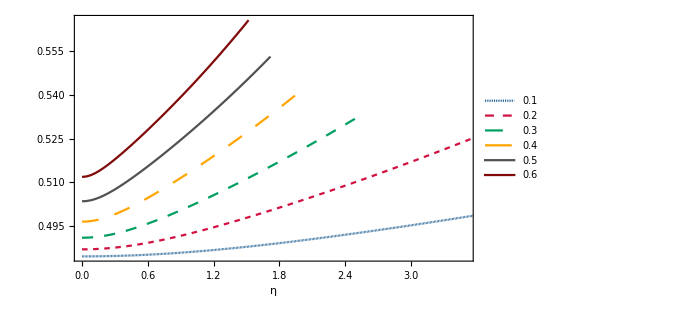

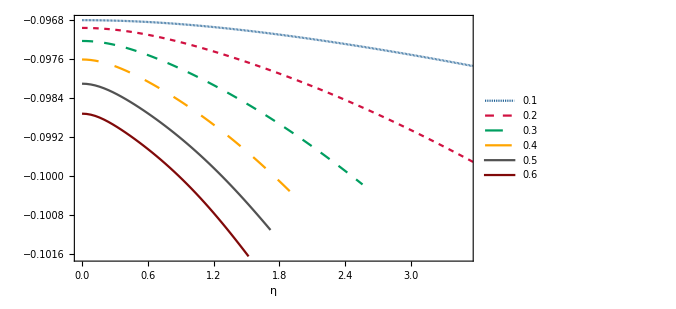

```mathematica
ListLinePlot[{Re[Ts0[[1]]],Re[Ts0[[2]]],Re[Ts0[[3]]],Re[Ts0[[4]]],Re[Ts0[[5]]],Re[Ts0[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},Right],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[Ts0[[1]]],Im[Ts0[[2]]],Im[Ts0[[3]]],Im[Ts0[[4]]],Im[Ts0[[5]]],Im[Ts0[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},Automatic},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 14,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 14,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 14,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 14,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 14,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 14,FontFamily->"Times New Roman"]},{0.09,0.25}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
(Max[Re[Tsd0[[1]]]]-Min[Re[Tsd0[[1]]]])/Min[Re[Tsd0[[1]]]]*100
(Max[Im[Tsd0[[1]]]]-Min[Im[Tsd0[[1]]]])/Min[Im[Tsd0[[1]]]]*100
(Max[Re[Tsd0[[6]]]]-Min[Re[Tsd0[[6]]]])/Min[Re[Tsd0[[6]]]]*100
(Max[Im[Tsd0[[6]]]]-Min[Im[Tsd0[[6]]]])/Min[Im[Tsd0[[6]]]]*100
```

7.85702

-2.82363

10.5385

-2.8802

```mathematica
Ts0[[6]][[26]]
```

{1+ⅈ,0.54322+0.10027 ⅈ}

Deviation from the exact values

## L=2

### L=2 Static axial full w

#### Fundamental tone of the gravitational type

```mathematica
TAx1={{0,0.3736716844180343-0.08896231568893015 ⅈ},{1/10+ⅈ/10,0.3739323753315701-0.08899053296514481 ⅈ},
{1/5+ⅈ/5,0.3747444263999218-0.08907478661745848 ⅈ},{3/10+(3 ⅈ)/10,0.376196782562713-0.08921294584647242 ⅈ},{2/5+(2 ⅈ)/5,0.3784368878775585-0.08939811399669846 ⅈ},{1/2+ⅈ/2,0.3816771513700477-0.0896123792877075 ⅈ},{3/5+(3 ⅈ)/5,0.3862174694056283-0.08981367498745657 ⅈ},{7/10+(7 ⅈ)/10,0.39249849104206613-0.08990442643364718 ⅈ},{4/5+(4 ⅈ)/5,0.4012171854649754-0.08964322973328098 ⅈ}};
TAx2={{0,0.3736716844180343-0.08896231568893015 ⅈ},{1/10+ⅈ/10,0.3739330607641263-0.08899081051509686 ⅈ},{1/5+ⅈ/5,0.37475489170165877-0.08907928088856536 ⅈ},{3/10+(3 ⅈ)/10,0.3762458695001867-0.08923623401745474 ⅈ},{2/5+(2 ⅈ)/5,0.3785765078752014-0.08947465504059797 ⅈ},{1/2+ⅈ/2,0.38197410241857715-0.08981100908733837 ⅈ},{3/5+(3 ⅈ)/5,0.386730093630079-0.09026475904628474 ⅈ},{7/10+(7 ⅈ)/10,0.3932265607585867-0.09085848136922271 ⅈ},{4/5+(4 ⅈ)/5,0.40199166317132884-0.0916182873245387 ⅈ}};
TAx3={{0,0.3736716844180343-0.08896231568893015 ⅈ},{1/10+ⅈ/10,0.37393440405879086-0.088991355932607 ⅈ},{1/5+ⅈ/5,0.3747741950747349-0.08908766480054434 ⅈ},{3/10+(3 ⅈ)/10,0.3763276976494858-0.08927614814207441 ⅈ},{2/5+(2 ⅈ)/5,0.3787775420853754-0.08959149508387439 ⅈ},{1/2+ⅈ/2,0.3823208342494274-0.0900728460528368 ⅈ},{3/5+(3 ⅈ)/5,0.3871590160648515-0.09076137855364343 ⅈ},{7/10+(7 ⅈ)/10,0.3935065369336788-0.09170094308556645 ⅈ},{4/5+(4 ⅈ)/5,0.4016113854730204-0.09294102462646311 ⅈ}};
```

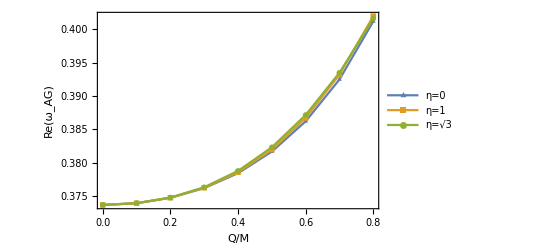

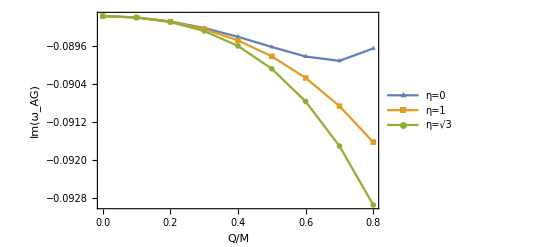

```mathematica
ListLinePlot[{Re[TAx1],Re[TAx2],Re[TAx3]},PlotMarkers->{▲,■,•},Frame->True,FrameLabel->{"Q/M",Re[Subscript[ω,AG]]},PlotLegends->{"η=0","η=1","η=√3"}]
ListLinePlot[{Im[TAx1],Im[TAx2],Im[TAx3]},PlotMarkers->{▲,■,•},Frame->True,FrameLabel->{"Q/M",Im[Subscript[ω,AG]]},PlotLegends->{"η=0","η=1","η=√3"}]
```

#### Fundamental tone of the electromagnetic type

```mathematica
TAx1={{0,0.45759551162985296-0.09500442581947172 ⅈ},{1/10+ⅈ/10,0.45892629047289313-0.09509719240882678 ⅈ},{1/5+ⅈ/5,0.4629651787153734-0.0953734357026487 ⅈ},{3/10+(3 ⅈ)/10,0.46986497341056693-0.09582639037141395 ⅈ},{2/5+(2 ⅈ)/5,0.4799259640854599-0.09644208522582358 ⅈ},{1/2+ⅈ/2,0.49367474352083845-0.09719236981371636 ⅈ},{3/5+(3 ⅈ)/5,0.5120109157124695-0.09801662953711017 ⅈ},{7/10+(7 ⅈ)/10,0.5365077467043715-0.09877141331419896 ⅈ},{4/5+(4 ⅈ)/5,0.5701302339628282-0.09906906228271489 ⅈ}};
TAx2={{0,0.45759551162985296-0.09500442581947172 ⅈ},{1/10 1+ⅈ/10,0.45892374703740685-0.09509729894728593 ⅈ},{1/5+ⅈ/5,0.46292416319363733-0.09537529185829306 ⅈ},{3/10+(3 ⅈ)/10,0.4696538460243859-0.09583711200348406 ⅈ},{2/5+(2 ⅈ)/5,0.4792382680394786-0.09648225996934132 ⅈ},{1/2+ⅈ/2,0.4919105809937164-0.09731273711767685 ⅈ},{3/5+(3 ⅈ)/5,0.5080636400212358-0.0983345289158112 ⅈ},{7/10+(7 ⅈ)/10,0.5283254873193048-0.09955868235956022 ⅈ},{4/5+(4 ⅈ)/5,0.5536845089399902-0.10100181698789763 ⅈ}};
TAx3={{0,0.45759551162985296-0.09500442581947172 ⅈ},{1/10+ⅈ/10,0.458918789724347-0.09509745479852444 ⅈ},{1/5+ⅈ/5,0.4628472790479511-0.09537782775736792 ⅈ},{3/10+(3 ⅈ)/10,0.4692819088903638-0.09585020248214215 ⅈ},{2/5+(2 ⅈ)/5,0.47812261515555643-0.0965242860930139 ⅈ},{1/2+ⅈ/2,0.48932371112836065-0.09741626459784383 ⅈ},{3/5+(3 ⅈ)/5,0.502931001140589-0.09854978479801811 ⅈ},{7/10+(7 ⅈ)/10,0.519104184514207-0.09995709214472778 ⅈ},{4/5+(4 ⅈ)/5,0.5381363069875619-0.10168105376211405 ⅈ}};
```

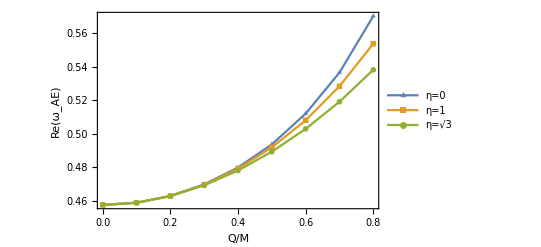

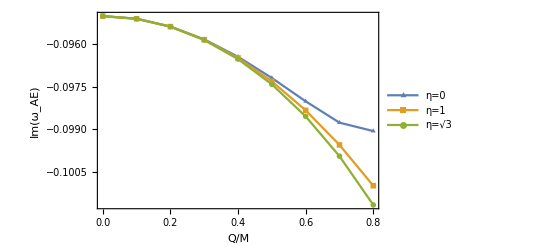

```mathematica
ListLinePlot[{Re[TAx1],Re[TAx2],Re[TAx3]},PlotMarkers->{▲,■,•},Frame->True,FrameLabel->{"Q/M",Re[Subscript[ω,AE]]},PlotLegends->{"η=0","η=1","η=√3"}]
ListLinePlot[{Im[TAx1],Im[TAx2],Im[TAx3]},PlotMarkers->{▲,■,•},Frame->True,FrameLabel->{"Q/M",Im[Subscript[ω,AE]]},PlotLegends->{"η=0","η=1","η=√3"}]
```

### L=2 Static axial o(w^2)

#### Fundamental tone of the gravitational type

```mathematica
TAxS1={{0,0.3736716844180343-0.08896231568893015 ⅈ},{1/10+ⅈ/10,0.37393376705486997-0.08899100402363531 ⅈ},{1/5+ⅈ/5,0.3747639359552871-0.0890821391496194 ⅈ},{3/10+(3 ⅈ)/10,0.37627476536748955-0.0892489077456262 ⅈ},{2/5+(2 ⅈ)/5,0.3786039734463023-0.08950785958445018 ⅈ},{1/2+ⅈ/2,0.3818729805013718-0.08987397394645535 ⅈ},{3/5+(3 ⅈ)/5,0.3861627008883921-0.09035720037462487 ⅈ},{7/10+(7 ⅈ)/10,0.39150651869305847-0.0909607828490125 ⅈ},{4/5+(4 ⅈ)/5,0.39789399751833715-0.09168100676828211 ⅈ}};
TAxS2={{0,0.3736716844180343-0.08896231568893015 ⅈ},{1/10+ⅈ/10,0.3739333534017907-0.08899069155645686 ⅈ},{1/5+ⅈ/5,0.3747580193416471-0.08907736597513594 ⅈ},{3/10+(3 ⅈ)/10,0.3762499373981195-0.08922644838952577 ⅈ},{2/5+(2 ⅈ)/5,0.3785441316088716-0.089443346992411 ⅈ},{1/2+ⅈ/2,0.3817731650709644-0.08973341013198746 ⅈ},{3/5+(3 ⅈ)/5,0.38604626045997886-0.09010085840669109 ⅈ},{7/10+(7 ⅈ)/10,0.3914410997912236-0.09054801715434323 ⅈ},{4/5+(4 ⅈ)/5,0.398003577387236-0.09107473040869236 ⅈ}};
TAxS3={{0,0.3736716844180343-0.08896231568893015 ⅈ},{1/10+ⅈ/10,0.37393356551226326-0.08899096508112692 ⅈ},{1/5+ⅈ/5,0.37476278874715246-0.08908212438738695 ⅈ},{3/10+(3 ⅈ)/10,0.3762840438680963-0.08925284573554847 ⅈ},{2/5+(2 ⅈ)/5,0.3786872206554331-0.08953194548408025 ⅈ},{1/2+ⅈ/2,0.38220481415949786-0.08994956790108315 ⅈ},{3/5+(3 ⅈ)/5,0.3870804164956674-0.09051185592295 ⅈ},{7/10+(7 ⅈ)/10,0.39352033428624333-0.09116948794546244 ⅈ},{4/5+(4 ⅈ)/5,0.4016275422764486-0.09180600730747626 ⅈ}};
```

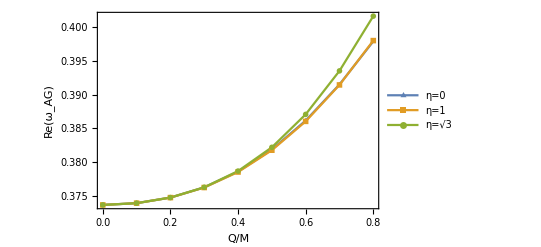

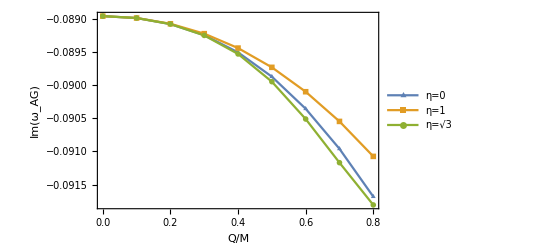

```mathematica
ListLinePlot[{Re[TAxS1],Re[TAxS2],Re[TAxS3]},PlotMarkers->{▲,■,•},Frame->True,FrameLabel->{"Q/M",Re[Subscript[ω,AG]]},PlotLegends->{"η=0","η=1","η=√3"}]
ListLinePlot[{Im[TAxS1],Im[TAxS2],Im[TAxS3]},PlotMarkers->{▲,■,•},Frame->True,FrameLabel->{"Q/M",Im[Subscript[ω,AG]]},PlotLegends->{"η=0","η=1","η=√3"}]
```

#### Fundamental tone of the electromagnetic type

```mathematica
TAxS1={{0,0.45759551162985296-0.09500442581947172 ⅈ},{1/10+ⅈ/10,0.45891692533497824-0.09509696629245468 ⅈ},{1/5+ⅈ/5,0.46281663668792006-0.09537012452062402 ⅈ},{3/10+(3 ⅈ)/10,0.46912084409053445-0.09581207154889763 ⅈ},{2/5+(2 ⅈ)/5,0.47759181379794763-0.09640710671223929 ⅈ},{1/2+ⅈ/2,0.48797244387806116-0.09713888013230201 ⅈ},{3/5+(3 ⅈ)/5,0.5000148814908246-0.09799213339786034 ⅈ},{7/10+(7 ⅈ)/10,0.5134930887031761-0.09895305513303511 ⅈ},{4/5+(4 ⅈ)/5,0.5282054780163924-0.10000887267310696 ⅈ}};
TAxS2={{0,0.45759551162985296-0.09500442581947172 ⅈ},{1/10+ⅈ/10,0.4589180562943222-0.09509689582192406 ⅈ},{1/5+ⅈ/5,0.4628340042043557-0.09536889508036346 ⅈ},{3/10+(3 ⅈ)/10,0.46920340991221826-0.09580515155716655 ⅈ},{2/5+(2 ⅈ)/5,0.47783303109019903-0.0963829760351722 ⅈ},{1/2+ⅈ/2,0.4885113320843496-0.09707526657245147 ⅈ},{3/5+(3 ⅈ)/5,0.5010316235426697-0.0978533211744392 ⅈ},{7/10+(7 ⅈ)/10,0.5152028399223532-0.09868912099404789 ⅈ},{4/5+(4 ⅈ)/5,0.5308525237712484-0.09955701105391312 ⅈ}};
TAxS3={{0,0.45759551162985296-0.09500442581947172 ⅈ},{1/10+ⅈ/10,0.45892139658325676-0.09509746871219575 ⅈ},{1/5+ⅈ/5,0.4628852621664609-0.09537670956914171 ⅈ},{3/10+(3 ⅈ)/10,0.4694459243342548-0.09583448107527186 ⅈ},{2/5+(2 ⅈ)/5,0.4785321507712653-0.09643718606409295 ⅈ},{1/2+ⅈ/2,0.49003189533673613-0.09711058994518101 ⅈ},{3/5+(3 ⅈ)/5,0.5037742696149526-0.09774142579049545 ⅈ},{7/10+(7 ⅈ)/10,0.519514084070743-0.09819961129994173 ⅈ},{4/5+(4 ⅈ)/5,0.5369308743569673-0.09837308481306255 ⅈ}};
```

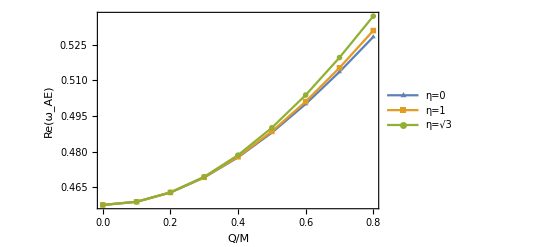

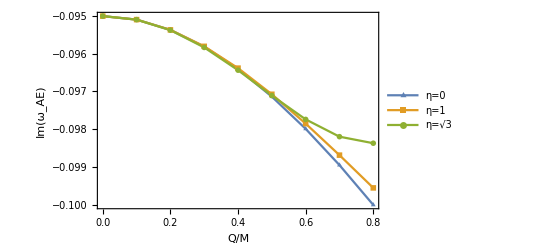

```mathematica
ListLinePlot[{Re[TAxS1],Re[TAxS2],Re[TAxS3]},PlotMarkers->{▲,■,•},Frame->True,FrameLabel->{"Q/M",Re[Subscript[ω,AE]]},PlotLegends->{"η=0","η=1","η=√3"}]
ListLinePlot[{Im[TAxS1],Im[TAxS2],Im[TAxS3]},PlotMarkers->{▲,■,•},Frame->True,FrameLabel->{"Q/M",Im[Subscript[ω,AE]]},PlotLegends->{"η=0","η=1","η=√3"}]
```

### L=2 Axial Comparison

#### Gravitational type

```mathematica
DIFF[ν0_]:=(
Module[{k},{
For[k=0, k<ν0+1,{
d1[k]={N[k/10]+I*N[k/10],Abs[(Re[TAx1]-Re[TAxS1])[[k+1]][[2]]/(Re[TAx1][[k+1]][[2]])]*100+I*Abs[(Im[TAx1]-Im[TAxS1])[[k+1]][[2]]/(Im[TAx1][[k+1]][[2]])]*100};
d2[k]={N[k/10]+I*N[k/10],Abs[(Re[TAx2]-Re[TAxS2])[[k+1]][[2]]/(Re[TAx2][[k+1]][[2]])]*100+I*Abs[(Im[TAx2]-Im[TAxS2])[[k+1]][[2]]/(Im[TAx2][[k+1]][[2]])]*100};
d3[k]={N[k/10]+I*N[k/10],Abs[(Re[TAx3]-Re[TAxS3])[[k+1]][[2]]/(Re[TAx3][[k+1]][[2]])]*100+I*Abs[(Im[TAx3]-Im[TAxS3])[[k+1]][[2]]/(Im[TAx3][[k+1]][[2]])]*100};
k++
}];
}];
D1=Table[d1[i],{i,0,ν0}];
D2=Table[d2[i],{i,0,ν0}];
D3=Table[d3[i],{i,0,ν0}];
);
```

```mathematica
DIFF[8]
```

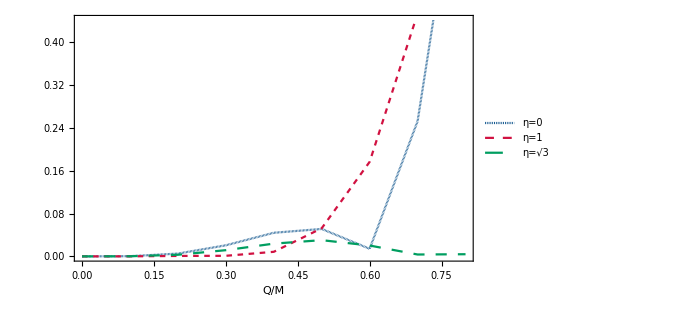

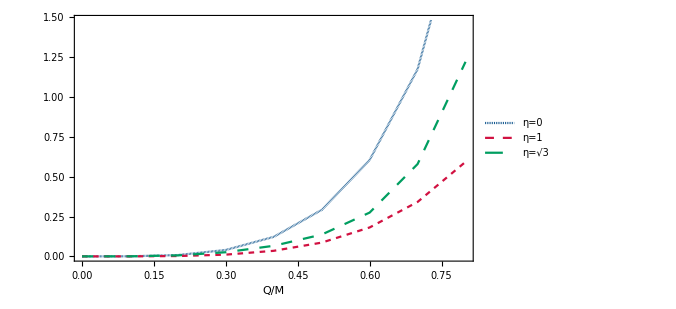

```mathematica
ListLinePlot[{Re[D1],Re[D2],Re[D3]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["Q/M"],20],None},ImageSize->500,PlotRange->{{0,0.8},Automatic},PlotLegends->
Placed[{Style[HoldForm["η=0"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["η=1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["η=√3"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.2,0.5}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[D1],Im[D2],Im[D3]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["Q/M"],20],None},ImageSize->500,PlotRange->{{0,0.8},Automatic},PlotLegends->
Placed[{Style[HoldForm["η=0"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["η=1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["η=√3"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.2,0.5}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

#### Electromagnetic type

```mathematica
DIFF[ν0_]:=(
Module[{k},{
For[k=0, k<ν0+1,{
d1[k]={N[k/10]+I*N[k/10],Abs[(Re[TAx1]-Re[TAxS1])[[k+1]][[2]]/(Re[TAx1][[k+1]][[2]])]*100+I*Abs[(Im[TAx1]-Im[TAxS1])[[k+1]][[2]]/(Im[TAx1][[k+1]][[2]])]*100};
d2[k]={N[k/10]+I*N[k/10],Abs[(Re[TAx2]-Re[TAxS2])[[k+1]][[2]]/(Re[TAx2][[k+1]][[2]])]*100+I*Abs[(Im[TAx2]-Im[TAxS2])[[k+1]][[2]]/(Im[TAx2][[k+1]][[2]])]*100};
d3[k]={N[k/10]+I*N[k/10],Abs[(Re[TAx3]-Re[TAxS3])[[k+1]][[2]]/(Re[TAx3][[k+1]][[2]])]*100+I*Abs[(Im[TAx3]-Im[TAxS3])[[k+1]][[2]]/(Im[TAx3][[k+1]][[2]])]*100};
k++
}];
}];
D1=Table[d1[i],{i,0,ν0}];
D2=Table[d2[i],{i,0,ν0}];
D3=Table[d3[i],{i,0,ν0}];
);
```

```mathematica
DIFF[8]
```

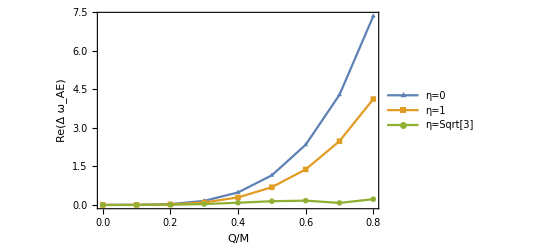

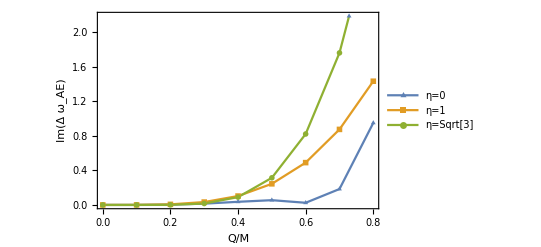

```mathematica
ListLinePlot[{Re[D1],Re[D2],Re[D3]},Frame->True,FrameLabel->{"Q/M",Re[Δ Subscript[ω,AE]]},PlotLegends->Placed[{"η=0","η=1","η=Sqrt[3]"},Center],PlotMarkers->{▲,■,●}]
ListLinePlot[{Im[D1],Im[D2],Im[D3]},Frame->True,FrameLabel->{"Q/M",Im[Δ Subscript[ω,AE]]},PlotLegends->Placed[{"η=0","η=1","η=Sqrt[3]"},Center],PlotMarkers->{▲,■,●}]
```

## L=1

### L=1 EM axial full-w

```mathematica
TAx1={{0,0.24826326417810868-0.0924877179529422 ⅈ},{1/10+ⅈ/10,0.2490546638256317-0.09259113445867317 ⅈ},{1/5+ⅈ/5,0.25147517221437055-0.09290233832982439 ⅈ},{3/10+(3 ⅈ)/10,0.2556720464108321-0.0934235700021665 ⅈ},{2/5+(2 ⅈ)/5,0.261921739340693-0.0941559525383815 ⅈ},{1/2+ⅈ/2,0.27069023094388633-0.09509309558616558 ⅈ},{3/5+(3 ⅈ)/5,0.28275662937978197-0.09620395766273489 ⅈ},{7/10+(7 ⅈ)/10,0.2994833757909741-0.09738248811443938 ⅈ},{4/5+(4 ⅈ)/5,0.32349359826840907-0.09827249955136529 ⅈ}};
TAx2={{0,0.24826326417810868-0.0924877179529422 ⅈ},{1/10+ⅈ/10,0.24905298795916442-0.09259118451453431 ⅈ},{1/5+ⅈ/5,0.25144765629360655-0.09290322084200622 ⅈ},{3/10+(3 ⅈ)/10,0.2555264441077003-0.09342880094621167 ⅈ},{2/5+(2 ⅈ)/5,0.26143084653467297-0.09417643994082617 ⅈ},{1/2+ⅈ/2,0.26938128334912426-0.0951585708757554 ⅈ},{3/5+(3 ⅈ)/5,0.27970593090537677-0.09639214708863596 ⅈ},{7/10+(7 ⅈ)/10,0.29289035644137074-0.09789952128388164 ⅈ},{4/5+(4 ⅈ)/5,0.30966574524485113-0.09970956535402116 ⅈ}};
TAx3={{0,0.24826326417810868-0.0924877179529422 ⅈ},{1/10+ⅈ/10,0.24904989269232533-0.09259125818676611 ⅈ},{1/5+ⅈ/5,0.25139884819140407-0.0929043695474872 ⅈ},{3/10+(3 ⅈ)/10,0.2552845773135526-0.09343439924911805 ⅈ},{2/5+(2 ⅈ)/5,0.2606849199438757-0.0941933701709171 ⅈ},{1/2+ⅈ/2,0.26760230766553383-0.09519814429755664 ⅈ},{3/5+(3 ⅈ)/5,0.2760827611180166-0.09647124687043312 ⅈ},{7/10+(7 ⅈ)/10,0.28623209107045783-0.09804251435555274 ⅈ},{4/5+(4 ⅈ)/5,0.2982322894872557-0.09995172260608765 ⅈ}};
```

### L=1 EM axial O(v^2)

```mathematica
TAxS1={{0,0.24826326417810868-0.0924877179529422 ⅈ},{1/10+ⅈ/10,0.24904963040596162-0.09259085005107101 ⅈ},{1/5+ⅈ/5,0.25139375215292903-0.09289789019610832 ⅈ},{3/10+(3 ⅈ)/10,0.2552518819430101-0.09340197972970332 ⅈ},{2/5+(2 ⅈ)/5,0.2605548349320549-0.09409233948704322 ⅈ},{1/2+ⅈ/2,0.2672128905242192-0.09495509910371647 ⅈ},{3/5+(3 ⅈ)/5,0.2751214923911891-0.09597421594016631 ⅈ},{7/10+(7 ⅈ)/10,0.28416699017328845-0.09713234153375482 ⅈ},{4/5+(4 ⅈ)/5,0.2942318325682706-0.09841154189386164 ⅈ}};
TAxS2={{0,0.24826326417810868-0.0924877179529422 ⅈ},{1/10+ⅈ/10,0.249050167970266-0.09259080421333697 ⅈ},{1/5+ⅈ/5,0.2514022199513174-0.09289710081475101 ⅈ},{3/10+(3 ⅈ)/10,0.25529366081771027-0.09339755125659764 ⅈ},{2/5+(2 ⅈ)/5,0.2606822781802847-0.09407667277617317 ⅈ},{1/2+ⅈ/2,0.2675104703045639-0.09491249442660694 ⅈ},{3/5+(3 ⅈ)/5,0.27570675049312204-0.0958772080221393 ⅈ},{7/10+(7 ⅈ)/10,0.2851877559496968-0.0969387380739911 ⅈ},{4/5+(4 ⅈ)/5,0.29586081366632266-0.09806308063902044 ⅈ}};
TAxS3={{0,0.24826326417810868-0.0924877179529422 ⅈ},{1/10+ⅈ/10,0.2490514245428817-0.09259080651430582 ⅈ},{1/5+ⅈ/5,0.2514219677731219-0.09289651634093093 ⅈ},{3/10+(3 ⅈ)/10,0.2553904161827787-0.09338959445248973 ⅈ},{2/5+(2 ⅈ)/5,0.2609726256062579-0.09403115916717973 ⅈ},{1/2+ⅈ/2,0.2681667638511916-0.09474532581120804 ⅈ},{3/5+(3 ⅈ)/5,0.2769260709649957-0.09541457267129175 ⅈ},{7/10+(7 ⅈ)/10,0.2871294959742962-0.09589498506165722 ⅈ},{4/5+(4 ⅈ)/5,0.29856638927920004-0.09605418107514171 ⅈ}};
```

### L=1 Axial Comparison

```mathematica
DIFF[ν0_]:=(
Module[{k},{
For[k=0, k<ν0+1,{
d1[k]={N[k/10]+I*N[k/10],Abs[(Re[TAx1]-Re[TAxS1])[[k+1]][[2]]/(Re[TAx1][[k+1]][[2]])]*100+I*Abs[(Im[TAx1]-Im[TAxS1])[[k+1]][[2]]/(Im[TAx1][[k+1]][[2]])]*100};
d2[k]={N[k/10]+I*N[k/10],Abs[(Re[TAx2]-Re[TAxS2])[[k+1]][[2]]/(Re[TAx2][[k+1]][[2]])]*100+I*Abs[(Im[TAx2]-Im[TAxS2])[[k+1]][[2]]/(Im[TAx2][[k+1]][[2]])]*100};
d3[k]={N[k/10]+I*N[k/10],Abs[(Re[TAx3]-Re[TAxS3])[[k+1]][[2]]/(Re[TAx3][[k+1]][[2]])]*100+I*Abs[(Im[TAx3]-Im[TAxS3])[[k+1]][[2]]/(Im[TAx3][[k+1]][[2]])]*100};
k++
}];
}];
D1=Table[d1[i],{i,0,ν0}];
D2=Table[d2[i],{i,0,ν0}];
D3=Table[d3[i],{i,0,ν0}];
);
```

```mathematica
DIFF[8]
```

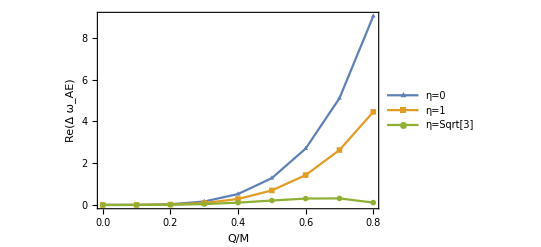

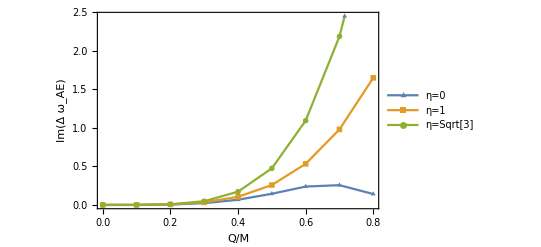

```mathematica
ListLinePlot[{Re[D1],Re[D2],Re[D3]},Frame->True,FrameLabel->{"Q/M",Re[Δ Subscript[ω,AE]]},PlotLegends->Placed[{"η=0","η=1","η=Sqrt[3]"},Center],PlotMarkers->{▲,■,●}]
ListLinePlot[{Im[D1],Im[D2],Im[D3]},Frame->True,FrameLabel->{"Q/M",Im[Δ Subscript[ω,AE]]},PlotLegends->Placed[{"η=0","η=1","η=Sqrt[3]"},Center],PlotMarkers->{▲,■,●}]
```

Slow rotation QNMs

## L=2 gravitational modes

NOTE: I have used at=0.2 and m=1

### Axial modes

#### Slow-rotation QNMs

```mathematica
T1={{{0,0.3873368034762385-0.08938807850266983 ⅈ},{1/25+ⅈ/25,0.38733680102811674-0.08938807869189422 ⅈ},{2/25+(2 ⅈ)/25,0.3873367936885917-0.08938807926349163 ⅈ},{3/25+(3 ⅈ)/25,0.3873367814722081-0.08938808022923254 ⅈ},{4/25+(4 ⅈ)/25,0.38733676440320436-0.0893880816087334 ⅈ},{1/5+ⅈ/5,0.38733674251551603-0.08938808342945374 ⅈ},{6/25+(6 ⅈ)/25,0.38733671585277873-0.08938808572669416 ⅈ},{7/25+(7 ⅈ)/25,0.38733668446833097-0.08938808854359082 ⅈ},{8/25+(8 ⅈ)/25,0.3873366484252165-0.08938809193111193 ⅈ},{9/25+(9 ⅈ)/25,0.3873366077961892-0.0893880959480517 ⅈ},{2/5+(2 ⅈ)/5,0.38733656266371896-0.08938810066102233 ⅈ},{11/25+(11 ⅈ)/25,0.38733651311999284-0.08938810614444984 ⅈ},{12/25+(12 ⅈ)/25,0.3873364592669279-0.08938811248056111 ⅈ},{13/25+(13 ⅈ)/25,0.38733640121617086-0.08938811975937809 ⅈ},{14/25+(14 ⅈ)/25,0.38733633908910875-0.08938812807870646 ⅈ},{3/5+(3 ⅈ)/5,0.3873362730168775-0.08938813754412427 ⅈ},{16/25+(16 ⅈ)/25,0.3873362031403661-0.08938814826896915 ⅈ},{17/25+(17 ⅈ)/25,0.38733612961023245-0.08938816037432797 ⅈ},{18/25+(18 ⅈ)/25,0.38733605258690923-0.08938817398901927 ⅈ},{19/25+(19 ⅈ)/25,0.3873359722406057-0.08938818924958167 ⅈ},{4/5+(4 ⅈ)/5,0.387335888751336-0.08938820630025641 ⅈ},{21/25+(21 ⅈ)/25,0.3873358023089179-0.08938822529297087 ⅈ},{22/25+(22 ⅈ)/25,0.38733571311298925-0.08938824638732111 ⅈ},{23/25+(23 ⅈ)/25,0.38733562137301847-0.08938826975055329 ⅈ},{24/25+(24 ⅈ)/25,0.38733552730832027-0.08938829555754384 ⅈ},{1+ⅈ,0.3873354311480675-0.08938832399077899 ⅈ},{26/25+(26 ⅈ)/25,0.3873353331313061-0.08938835524033312 ⅈ},{27/25+(27 ⅈ)/25,0.3873352335069702-0.0893883895038474 ⅈ},{28/25+(28 ⅈ)/25,0.3873351325338984-0.08938842698650368 ⅈ},{29/25+(29 ⅈ)/25,0.3873350304808485-0.08938846790100229 ⅈ},{6/5+(6 ⅈ)/5,0.3873349276265147-0.08938851246753546 ⅈ},{31/25+(31 ⅈ)/25,0.3873348242595454-0.08938856091376099 ⅈ},{32/25+(32 ⅈ)/25,0.3873347206785604-0.0893886134747743 ⅈ},{33/25+(33 ⅈ)/25,0.38733461719216894-0.08938867039308002 ⅈ},{34/25+(34 ⅈ)/25,0.38733451411898956-0.08938873191856195 ⅈ},{7/5+(7 ⅈ)/5,0.38733441178766875-0.08938879830845241 ⅈ},{36/25+(36 ⅈ)/25,0.387334310536901-0.08938886982730014 ⅈ},{37/25+(37 ⅈ)/25,0.3873342107154496-0.08938894674693745 ⅈ},{38/25+(38 ⅈ)/25,0.3873341126821671-0.08938902934644552 ⅈ},{39/25+(39 ⅈ)/25,0.38733401680601726-0.08938911791211977 ⅈ},{8/5+(8 ⅈ)/5,0.38733392346609674-0.08938921273743299 ⅈ},{41/25+(41 ⅈ)/25,0.38733383305165764-0.08938931412299779 ⅈ},{42/25+(42 ⅈ)/25,0.3873337459621307-0.08938942237652771 ⅈ},{43/25+(43 ⅈ)/25,0.3873336626071483-0.08938953781279764 ⅈ},{44/25+(44 ⅈ)/25,0.3873335834065687-0.08938966075360183 ⅈ},{9/5+(9 ⅈ)/5,0.3873335087905003-0.08938979152771248 ⅈ},{46/25+(46 ⅈ)/25,0.3873334391993267-0.08938993047083514 ⅈ},{47/25+(47 ⅈ)/25,0.387333375083731-0.08939007792556465 ⅈ},{48/25+(48 ⅈ)/25,0.38733331690472284-0.0893902342413382 ⅈ},{49/25+(49 ⅈ)/25,0.3873332651336635-0.0893903997743883 ⅈ},{2+2 ⅈ,0.3873332202522925-0.08939057488769395 ⅈ},{51/25+(51 ⅈ)/25,0.3873331827527551-0.08939075995093052 ⅈ},{52/25+(52 ⅈ)/25,0.38733315313762895-0.08939095534041798 ⅈ},{53/25+(53 ⅈ)/25,0.38733313191995156-0.08939116143906882 ⅈ},{54/25+(54 ⅈ)/25,0.387333119623249-0.08939137863633309 ⅈ},{11/5+(11 ⅈ)/5,0.387333116781564-0.08939160732814329 ⅈ},{56/25+(56 ⅈ)/25,0.38733312393948394-0.0893918479168572 ⅈ},{57/25+(57 ⅈ)/25,0.3873331416521708-0.08939210081119939 ⅈ},{58/25+(58 ⅈ)/25,0.38733317048538995-0.08939236642620148 ⅈ},{59/25+(59 ⅈ)/25,0.3873332110155397-0.08939264518314056 ⅈ},{12/5+(12 ⅈ)/5,0.3873332638296806-0.08939293750947656 ⅈ},{61/25+(61 ⅈ)/25,0.3873333295255672-0.08939324383878743 ⅈ},{62/25+(62 ⅈ)/25,0.38733340871167626-0.08939356461070379 ⅈ},{63/25+(63 ⅈ)/25,0.38733350200723893-0.08939390027084068 ⅈ},{64/25+(64 ⅈ)/25,0.38733361004227035-0.0893942512707292 ⅈ},{13/5+(13 ⅈ)/5,0.38733373345760136-0.08939461806774529 ⅈ},{66/25+(66 ⅈ)/25,0.38733387290490917-0.08939500112503772 ⅈ},{67/25+(67 ⅈ)/25,0.3873340290467486-0.08939540091145362 ⅈ},{68/25+(68 ⅈ)/25,0.38733420255658363-0.08939581790146352 ⅈ},{69/25+(69 ⅈ)/25,0.38733439411881865-0.08939625257508352 ⅈ},{14/5+(14 ⅈ)/5,0.38733460442883-0.08939670541779592 ⅈ},{71/25+(71 ⅈ)/25,0.38733483419299763-0.08939717692046939 ⅈ},{72/25+(72 ⅈ)/25,0.3873350841287367-0.08939766757927523 ⅈ},{73/25+(73 ⅈ)/25,0.3873353549645292-0.08939817789560373 ⅈ},{74/25+(74 ⅈ)/25,0.38733564743995547-0.08939870837597766 ⅈ},{3+3 ⅈ,0.3873359623057262-0.08939925953196423 ⅈ},{76/25+(76 ⅈ)/25,0.3873363003237131-0.08939983188008518 ⅈ},{77/25+(77 ⅈ)/25,0.387336662266981-0.08940042594172529 ⅈ},{78/25+(78 ⅈ)/25,0.3873370489198194-0.0894010422430381 ⅈ},{79/25+(79 ⅈ)/25,0.3873374610777728-0.08940168131485049 ⅈ},{16/5+(16 ⅈ)/5,0.38733789954767195-0.0894023436925654 ⅈ},{81/25+(81 ⅈ)/25,0.3873383651476651-0.08940302991606158 ⅈ},{82/25+(82 ⅈ)/25,0.38733885870724843-0.08940374052959248 ⅈ},{83/25+(83 ⅈ)/25,0.38733938106729526-0.08940447608168242 ⅈ},{84/25+(84 ⅈ)/25,0.3873399330800879-0.08940523712502083 ⅈ},{17/5+(17 ⅈ)/5,0.38734051560934535-0.08940602421635434 ⅈ},{86/25+(86 ⅈ)/25,0.38734112953025385-0.08940683791637709 ⅈ},{87/25+(87 ⅈ)/25,0.3873417757294957-0.08940767878961862 ⅈ},{88/25+(88 ⅈ)/25,0.38734245510527654-0.08940854740432945 ⅈ},{89/25+(89 ⅈ)/25,0.3873431685673551-0.08940944433236477 ⅈ},{18/5+(18 ⅈ)/5,0.3873439170370687-0.08941037014906585 ⅈ},{91/25+(91 ⅈ)/25,0.387344701447362-0.08941132543313926 ⅈ},{92/25+(92 ⅈ)/25,0.38734552274281125-0.08941231076653368 ⅈ},{93/25+(93 ⅈ)/25,0.3873463818796523-0.08941332673431412 ⅈ},{94/25+(94 ⅈ)/25,0.3873472798258035-0.08941437392453513 ⅈ},{19/5+(19 ⅈ)/5,0.3873482175608908-0.08941545292810978 ⅈ},{96/25+(96 ⅈ)/25,0.3873491960762718-0.08941656433867763 ⅈ},{97/25+(97 ⅈ)/25,0.3873502163750573-0.08941770875247032 ⅈ},{98/25+(98 ⅈ)/25,0.387351279472134-0.08941888676817354 ⅈ},{99/25+(99 ⅈ)/25,0.38735238639418496-0.08942009898678847 ⅈ},{4+4 ⅈ,0.3873535381797095-0.08942134601148904 ⅈ},{101/25+(101 ⅈ)/25,0.3873547358790427-0.08942262844747742 ⅈ},{102/25+(102 ⅈ)/25,0.3873559805543727-0.08942394690183716 ⅈ},{103/25+(103 ⅈ)/25,0.38735727327975783-0.08942530198338385 ⅈ},{104/25+(104 ⅈ)/25,0.3873586151411422-0.08942669430251293 ⅈ},{21/5+(21 ⅈ)/5,0.38736000723636965-0.08942812447104483 ⅈ},{106/25+(106 ⅈ)/25,0.3873614506751979-0.08942959310206827 ⅈ},{107/25+(107 ⅈ)/25,0.38736294657930886-0.0894311008097802 ⅈ},{108/25+(108 ⅈ)/25,0.3873644960823209-0.08943264820932353 ⅈ},{109/25+(109 ⅈ)/25,0.38736610032979596-0.08943423591662211 ⅈ},{22/5+(22 ⅈ)/5,0.38736776047924826-0.08943586454821335 ⅈ},{111/25+(111 ⅈ)/25,0.3873694777001499-0.08943753472107736 ⅈ},{112/25+(112 ⅈ)/25,0.38737125317393417-0.08943924705246492 ⅈ},{113/25+(113 ⅈ)/25,0.387373088094-0.0894410021597209 ⅈ},{114/25+(114 ⅈ)/25,0.3873749836657104-0.08944280066010657 ⅈ},{23/5+(23 ⅈ)/5,0.38737694110639315-0.08944464317061833 ⅈ},{116/25+(116 ⅈ)/25,0.3873789616453372-0.08944653030780426 ⅈ},{117/25+(117 ⅈ)/25,0.38738104652378746-0.089448462687577 ⅈ},{118/25+(118 ⅈ)/25,0.3873831969949378-0.08945044092502534 ⅈ},{119/25+(119 ⅈ)/25,0.3873854143239221-0.08945246563422155 ⅈ},{24/5+(24 ⅈ)/5,0.38738769978780335-0.08945453742802725 ⅈ},{121/25+(121 ⅈ)/25,0.38739005467555876-0.08945665691789566 ⅈ},{122/25+(122 ⅈ)/25,0.3873924802880647-0.08945882471367136 ⅈ},{123/25+(123 ⅈ)/25,0.3873949779380781-0.08946104142338737 ⅈ},{124/25+(124 ⅈ)/25,0.38739754895021533-0.08946330765305954 ⅈ},{5+5 ⅈ,0.38740019466092857-0.08946562400647781 ⅈ},{126/25+(126 ⅈ)/25,0.38740291641848007-0.0894679910849952 ⅈ},{127/25+(127 ⅈ)/25,0.3874057155829122-0.08947040948731348 ⅈ},{128/25+(128 ⅈ)/25,0.3874085935260166-0.08947287980926683 ⅈ},{129/25+(129 ⅈ)/25,0.3874115516312984-0.08947540264360172 ⅈ},{26/5+(26 ⅈ)/5,0.3874145912939394-0.08947797857975572 ⅈ},{131/25+(131 ⅈ)/25,0.3874177139207562-0.08948060820363112 ⅈ},{132/25+(132 ⅈ)/25,0.3874209209301562-0.08948329209736863 ⅈ},{133/25+(133 ⅈ)/25,0.38742421375209074-0.0894860308391162 ⅈ},{134/25+(134 ⅈ)/25,0.38742759382800324-0.08948882500279634 ⅈ},{27/5+(27 ⅈ)/5,0.387431062610775-0.08949167515787025 ⅈ},{136/25+(136 ⅈ)/25,0.38743462156466857-0.08949458186909978 ⅈ},{137/25+(137 ⅈ)/25,0.38743827216526333-0.08949754569630637 ⅈ},{138/25+(138 ⅈ)/25,0.3874420158993932-0.08950056719412745 ⅈ},{139/25+(139 ⅈ)/25,0.3874458542650744-0.08950364691177065 ⅈ},{28/5+(28 ⅈ)/5,0.38744978877143404-0.08950678539276505 ⅈ},{141/25+(141 ⅈ)/25,0.3874538209386313-0.08950998317471072 ⅈ},{142/25+(142 ⅈ)/25,0.3874579522977771-0.08951324078902403 ⅈ},{143/25+(143 ⅈ)/25,0.3874621843908466-0.08951655876068329 ⅈ},{144/25+(144 ⅈ)/25,0.3874665187705903-0.08951993760796945 ⅈ},{29/5+(29 ⅈ)/5,0.38747095700043727-0.08952337784220613 ⅈ},{146/25+(146 ⅈ)/25,0.3874755006543983-0.08952687996749624 ⅈ},{147/25+(147 ⅈ)/25,0.3874801513169584-0.0895304444804577 ⅈ},{148/25+(148 ⅈ)/25,0.38748491058296985-0.08953407186995614 ⅈ},{149/25+(149 ⅈ)/25,0.387489780057537-0.0895377626168358 ⅈ},{6+6 ⅈ,0.3874947613558994-0.08954151719364624 ⅈ},{151/25+(151 ⅈ)/25,0.3874998561033029-0.08954533606437336 ⅈ},{152/25+(152 ⅈ)/25,0.38750506593487427-0.08954921968416026 ⅈ},{153/25+(153 ⅈ)/25,0.3875103924954856-0.08955316849903185 ⅈ},{154/25+(154 ⅈ)/25,0.38751583743960955-0.08955718294561708 ⅈ},{31/5+(31 ⅈ)/5,0.3875214024311796-0.0895612634508672 ⅈ},{156/25+(156 ⅈ)/25,0.3875270891434334-0.0895654104317745 ⅈ},{157/25+(157 ⅈ)/25,0.3875328992587566-0.08956962429508893 ⅈ},{158/25+(158 ⅈ)/25,0.3875388344685191-0.08957390543703346 ⅈ},{159/25+(159 ⅈ)/25,0.38754489647290513-0.08957825424301828 ⅈ},{32/5+(32 ⅈ)/5,0.3875510869807381-0.08958267108735028 ⅈ},{161/25+(161 ⅈ)/25,0.38755740770929337-0.0895871563329548 ⅈ},{162/25+(162 ⅈ)/25,0.3875638603841203-0.08959171033107526 ⅈ},{163/25+(163 ⅈ)/25,0.38757044673882723-0.08959633342098708 ⅈ},{164/25+(164 ⅈ)/25,0.3875771685149233-0.08960102592969343 ⅈ},{33/5+(33 ⅈ)/5,0.3875840274615391-0.08960578817167714 ⅈ},{166/25+(166 ⅈ)/25,0.38759102533527423-0.08961062044856052 ⅈ},{167/25+(167 ⅈ)/25,0.3875981638999469-0.08961552304882961 ⅈ},{168/25+(168 ⅈ)/25,0.387605444926371-0.08962049624755192 ⅈ},{169/25+(169 ⅈ)/25,0.3876128701921157-0.0896255403060707 ⅈ},{34/5+(34 ⅈ)/5,0.38762044148126495-0.08963065547172011 ⅈ},{171/25+(171 ⅈ)/25,0.38762816058416466-0.08963584197753086 ⅈ},{172/25+(172 ⅈ)/25,0.38763602929716173-0.08964110004193794 ⅈ},{173/25+(173 ⅈ)/25,0.3876440494223446-0.08964642986849267 ⅈ},{174/25+(174 ⅈ)/25,0.38765222276725925-0.08965183164556705 ⅈ},{7+7 ⅈ,0.3876605511446377-0.0896573055460685 ⅈ},{176/25+(176 ⅈ)/25,0.3876690363720984-0.08966285172715187 ⅈ},{177/25+(177 ⅈ)/25,0.38767768027185906-0.08966847032992803 ⅈ},{178/25+(178 ⅈ)/25,0.38768648467042305-0.08967416147918413 ⅈ}},{{0,0.3883864882314263-0.08948148934863873 ⅈ},{1/25+ⅈ/25,0.3883864696861285-0.08948148334523565 ⅈ},{2/25+(2 ⅈ)/25,0.38838641412604397-0.08948146539909528 ⅈ},{3/25+(3 ⅈ)/25,0.38838632177879573-0.08948143570246328 ⅈ},{4/25+(4 ⅈ)/25,0.3883861930238036-0.08948139457563643 ⅈ},{1/5+ⅈ/5,0.38838602839239383-0.08948134246686519 ⅈ},{6/25+(6 ⅈ)/25,0.3883858285679503-0.08948127995216144 ⅈ},{7/25+(7 ⅈ)/25,0.38838559438609754-0.08948120773507041 ⅈ},{8/25+(8 ⅈ)/25,0.388385326834929-0.08948112664638763 ⅈ},{9/25+(9 ⅈ)/25,0.3883850270552735-0.08948103764382356 ⅈ},{2/5+(2 ⅈ)/5,0.38838469634100325-0.08948094181161427 ⅈ},{11/25+(11 ⅈ)/25,0.38838433613938295-0.08948084036007818 ⅈ},{12/25+(12 ⅈ)/25,0.38838394805145615-0.08948073462511784 ⅈ},{13/25+(13 ⅈ)/25,0.38838353383247526-0.08948062606766602 ⅈ},{14/25+(14 ⅈ)/25,0.3883830953923666-0.08948051627307427 ⅈ},{3/5+(3 ⅈ)/5,0.3883826347962365-0.0894804069504438 ⅈ},{16/25+(16 ⅈ)/25,0.3883821542649162-0.0894802999318971 ⅈ},{17/25+(17 ⅈ)/25,0.3883816561755426-0.08948019717178822 ⅈ},{18/25+(18 ⅈ)/25,0.3883811430621771-0.08948010074585143 ⅈ},{19/25+(19 ⅈ)/25,0.3883806176164609-0.08948001285028627 ⅈ},{4/5+(4 ⅈ)/5,0.38838008268830626-0.08947993580077694 ⅈ},{21/25+(21 ⅈ)/25,0.38837954128662205-0.0894798720314447 ⅈ},{22/25+(22 ⅈ)/25,0.3883789965800735-0.08947982409373151 ⅈ},{23/25+(23 ⅈ)/25,0.3883784518978763-0.08947979465521276 ⅈ},{24/25+(24 ⅈ)/25,0.38837791073062117-0.08947978649833711 ⅈ},{1+ⅈ,0.38837737673113026-0.08947980251909167 ⅈ},{26/25+(26 ⅈ)/25,0.38837685371534403-0.08947984572558973 ⅈ},{27/25+(27 ⅈ)/25,0.3883763456632364-0.08947991923657872 ⅈ},{28/25+(28 ⅈ)/25,0.38837585671975616-0.08948002627986718 ⅈ},{29/25+(29 ⅈ)/25,0.38837539119579634-0.08948017019066679 ⅈ},{6/5+(6 ⅈ)/5,0.3883749535691857-0.08948035440984708 ⅈ},{31/25+(31 ⅈ)/25,0.38837454848570513-0.08948058248210179 ⅈ},{32/25+(32 ⅈ)/25,0.38837418076012176-0.08948085805402171 ⅈ},{33/25+(33 ⅈ)/25,0.38837385537724545-0.0894811848720733 ⅈ},{34/25+(34 ⅈ)/25,0.38837357749299956-0.08948156678047844 ⅈ},{7/5+(7 ⅈ)/5,0.38837335243550725-0.08948200771899442 ⅈ},{36/25+(36 ⅈ)/25,0.38837318570619034-0.08948251172058828 ⅈ},{37/25+(37 ⅈ)/25,0.38837308298087714-0.08948308290900579 ⅈ},{38/25+(38 ⅈ)/25,0.38837305011091766-0.08948372549622889 ⅈ},{39/25+(39 ⅈ)/25,0.3883730931243039-0.08948444377982011 ⅈ},{8/5+(8 ⅈ)/5,0.3883732182267899-0.08948524214015022 ⅈ},{41/25+(41 ⅈ)/25,0.38837343180301104-0.08948612503750591 ⅈ},{42/25+(42 ⅈ)/25,0.38837374041759665-0.08948709700907385 ⅈ},{43/25+(43 ⅈ)/25,0.388374150816275-0.0894881626657978 ⅈ},{44/25+(44 ⅈ)/25,0.38837466992696457-0.08948932668910588 ⅈ},{9/5+(9 ⅈ)/5,0.3883753048608481-0.08949059382750393 ⅈ},{46/25+(46 ⅈ)/25,0.38837606291342597-0.08949196889303189 ⅈ},{47/25+(47 ⅈ)/25,0.3883769515655437-0.08949345675757951 ⅈ},{48/25+(48 ⅈ)/25,0.38837797848438854-0.08949506234905856 ⅈ},{49/25+(49 ⅈ)/25,0.3883791515244506-0.0894967906474269 ⅈ},{2+2 ⅈ,0.38838047872844256-0.08949864668056316 ⅈ},{51/25+(51 ⅈ)/25,0.38838196832817357-0.08950063551998609 ⅈ},{52/25+(52 ⅈ)/25,0.38838362874536925-0.0895027622764175 ⅈ},{53/25+(53 ⅈ)/25,0.3883854685924343-0.08950503209518532 ⅈ},{54/25+(54 ⅈ)/25,0.3883874966731486-0.08950745015146197 ⅈ},{11/5+(11 ⅈ)/5,0.3883897219832917-0.08951002164533756 ⅈ},{56/25+(56 ⅈ)/25,0.38839215371118757-0.08951275179672383 ⅈ},{57/25+(57 ⅈ)/25,0.38839480123816267-0.08951564584008542 ⅈ},{58/25+(58 ⅈ)/25,0.38839767413890885-0.08951870901899842 ⅈ},{59/25+(59 ⅈ)/25,0.38840078218174284-0.0895219465805312 ⅈ},{12/5+(12 ⅈ)/5,0.3884041353287553-0.0895253637694471 ⅈ},{61/25+(61 ⅈ)/25,0.38840774373583764-0.08952896582222697 ⅈ},{62/25+(62 ⅈ)/25,0.38841161775257976-0.08953275796091002 ⅈ},{63/25+(63 ⅈ)/25,0.3884157679220272-0.0895367453867508 ⅈ},{64/25+(64 ⅈ)/25,0.38842020498029034-0.08954093327369313 ⅈ},{13/5+(13 ⅈ)/5,0.3884249398559896-0.08954532676165909 ⅈ},{66/25+(66 ⅈ)/25,0.3884299836695339-0.08954993094965366 ⅈ},{67/25+(67 ⅈ)/25,0.38843534773221317-0.0895547508886846 ⅈ},{68/25+(68 ⅈ)/25,0.38844104354509856-0.08955979157449938 ⅈ},{69/25+(69 ⅈ)/25,0.3884470827977354-0.08956505794013954 ⅈ},{14/5+(14 ⅈ)/5,0.38845347736661845-0.08957055484831501 ⅈ},{71/25+(71 ⅈ)/25,0.38846023931343654-0.0895762870835995 ⅈ},{72/25+(72 ⅈ)/25,0.3884673808830709-0.08958225934445209 ⅈ},{73/25+(73 ⅈ)/25,0.3884749145013387-0.08958847623506647 ⅈ},{74/25+(74 ⅈ)/25,0.38848285277246175-0.08959494225705417 ⅈ},{3+3 ⅈ,0.3884912084762531-0.08960166180096538 ⅈ},{76/25+(76 ⅈ)/25,0.3884999945650032-0.08960863913765316 ⅈ},{77/25+(77 ⅈ)/25,0.3885092241600496-0.08961587840949127 ⅈ},{78/25+(78 ⅈ)/25,0.38851891054802046-0.08962338362144813 ⅈ},{79/25+(79 ⅈ)/25,0.3885290671767326-0.08963115863202827 ⅈ},{16/5+(16 ⅈ)/5,0.3885397076507349-0.08963920714409258 ⅈ},{81/25+(81 ⅈ)/25,0.3885508457264699-0.08964753269556319 ⅈ},{82/25+(82 ⅈ)/25,0.3885624953070538-0.08965613865003091 ⅈ},{83/25+(83 ⅈ)/25,0.38857467043664484-0.08966502818727394 ⅈ},{84/25+(84 ⅈ)/25,0.38858738529440484-0.08967420429369573 ⅈ},{17/5+(17 ⅈ)/5,0.3886006541880161-0.08968366975272012 ⅈ},{86/25+(86 ⅈ)/25,0.3886144915467429-0.08969342713512418 ⅈ},{87/25+(87 ⅈ)/25,0.388628911914049-0.08970347878936759 ⅈ},{88/25+(88 ⅈ)/25,0.38864392993972363-0.08971382683189655 ⅈ},{89/25+(89 ⅈ)/25,0.38865956037151816-0.08972447313748039 ⅈ},{18/5+(18 ⅈ)/5,0.3886758180462788-0.08973541932957173 ⅈ},{91/25+(91 ⅈ)/25,0.38869271788057363-0.08974666677073578 ⅈ}},{{0,0.3902637202984556-0.08965071610667376 ⅈ},{1/25+ⅈ/25,0.3902636524057578-0.08965067904178142 ⅈ},{2/25+(2 ⅈ)/25,0.39026344909660465-0.08965056817811051 ⅈ},{3/25+(3 ⅈ)/25,0.3902631114787153-0.08965038450880154 ⅈ},{4/25+(4 ⅈ)/25,0.39026264139898076-0.08965012968820939 ⅈ},{1/5+ⅈ/5,0.3902620414447326-0.08964980603070874 ⅈ},{6/25+(6 ⅈ)/25,0.39026131494542377-0.08964941650896162 ⅈ},{7/25+(7 ⅈ)/25,0.39026046597478575-0.08964896475167479 ⅈ},{8/25+(8 ⅈ)/25,0.3902594993534606-0.08964845504083578 ⅈ},{9/25+(9 ⅈ)/25,0.39025842065210276-0.08964789230841383 ⅈ},{2/5+(2 ⅈ)/5,0.3902572361949441-0.0896472821325103 ⅈ},{11/25+(11 ⅈ)/25,0.39025595306382377-0.0896466307329375 ⅈ},{12/25+(12 ⅈ)/25,0.3902545791026665-0.08964594496620802 ⅈ},{13/25+(13 ⅈ)/25,0.3902531229224121-0.0896452323199067 ⅈ},{14/25+(14 ⅈ)/25,0.39025159390638064-0.089644500906423 ⅈ},{3/5+(3 ⅈ)/5,0.3902500022160656-0.08964375945601152 ⅈ},{16/25+(16 ⅈ)/25,0.390248358797347-0.08964301730915093 ⅈ},{17/25+(17 ⅈ)/25,0.39024667538710384-0.08964228440816759 ⅈ},{18/25+(18 ⅈ)/25,0.39024496452022217-0.08964157128808604 ⅈ},{19/25+(19 ⅈ)/25,0.39024323953697143-0.08964088906666921 ⅈ},{4/5+(4 ⅈ)/5,0.3902415145907394-0.08964024943360537 ⅈ},{21/25+(21 ⅈ)/25,0.3902398046560989-0.08963966463879912 ⅈ},{22/25+(22 ⅈ)/25,0.39023812553718723-0.08963914747972014 ⅈ},{23/25+(23 ⅈ)/25,0.39023649387636794-0.08963871128776048 ⅈ},{24/25+(24 ⅈ)/25,0.3902349271631514-0.08963836991355104 ⅈ},{1+ⅈ,0.3902334437433365-0.08963813771118258 ⅈ},{26/25+(26 ⅈ)/25,0.39023206282834016-0.08963802952127846 ⅈ},{27/25+(27 ⅈ)/25,0.39023080450467507-0.08963806065286005 ⅈ},{28/25+(28 ⅈ)/25,0.39022968974353106-0.08963824686394826 ⅈ},{29/25+(29 ⅈ)/25,0.390228740410411-0.08963860434084014 ⅈ},{6/5+(6 ⅈ)/5,0.39022797927476893-0.08963914967599779 ⅈ},{31/25+(31 ⅈ)/25,0.39022743001959176-0.08963989984448942 ⅈ},{32/25+(32 ⅈ)/25,0.39022711725085873-0.08964087217891628 ⅈ},{33/25+(33 ⅈ)/25,0.39022706650681116-0.08964208434276368 ⅈ},{34/25+(34 ⅈ)/25,0.3902273042669529-0.08964355430210938 ⅈ},{7/5+(7 ⅈ)/5,0.39022785796069853-0.0896453002956275 ⅈ},{36/25+(36 ⅈ)/25,0.390228755975582-0.08964734080282191 ⅈ},{37/25+(37 ⅈ)/25,0.3902300276649219-0.08964969451042953 ⅈ},{38/25+(38 ⅈ)/25,0.3902317033548404-0.08965238027693023 ⅈ},{39/25+(39 ⅈ)/25,0.3902338143505208-0.08965541709510647 ⅈ},{8/5+(8 ⅈ)/5,0.3902363929415785-0.08965882405259816 ⅈ},{41/25+(41 ⅈ)/25,0.390239472406412-0.08966262029039886 ⅈ},{42/25+(42 ⅈ)/25,0.3902430870153952-0.08966682495924991 ⅈ},{43/25+(43 ⅈ)/25,0.39024727203275195-0.08967145717388877 ⅈ},{44/25+(44 ⅈ)/25,0.39025206371695564-0.08967653596511925 ⅈ},{9/5+(9 ⅈ)/5,0.39025749931947934-0.08968208022967569 ⅈ},{46/25+(46 ⅈ)/25,0.39026361708171003-0.0896881086778645 ⅈ},{47/25+(47 ⅈ)/25,0.3902704562298373-0.0896946397789762 ⅈ},{48/25+(48 ⅈ)/25,0.3902780569675062-0.08970169170447113 ⅈ},{49/25+(49 ⅈ)/25,0.3902864604660257-0.08970928226895797 ⅈ},{2+2 ⅈ,0.39029570885189857-0.08971742886899751 ⅈ},{51/25+(51 ⅈ)/25,0.39030584519144634-0.08972614841977979 ⅈ},{52/25+(52 ⅈ)/25,0.39031691347227737-0.08973545728974296 ⅈ},{53/25+(53 ⅈ)/25,0.3903289585813488-0.08974537123321974 ⅈ},{54/25+(54 ⅈ)/25,0.3903420262793615-0.08975590532122428 ⅈ},{11/5+(11 ⅈ)/5,0.39035616317121496-0.08976707387050642 ⅈ},{56/25+(56 ⅈ)/25,0.39037141667226416-0.08977889037104048 ⅈ},{57/25+(57 ⅈ)/25,0.3903878349700835-0.08979136741212611 ⅈ},{58/25+(58 ⅈ)/25,0.39040546698147655-0.08980451660732629 ⅈ},{59/25+(59 ⅈ)/25,0.39042436230444644-0.08981834851848709 ⅈ},{12/5+(12 ⅈ)/5,0.390444571164863-0.08983287257912784 ⅈ},{61/25+(61 ⅈ)/25,0.3904661443575518-0.08984809701749695 ⅈ},{62/25+(62 ⅈ)/25,0.3904891331815503-0.08986402877968351 ⅈ},{63/25+(63 ⅈ)/25,0.3905135893692979-0.08988067345314547 ⅈ},{64/25+(64 ⅈ)/25,0.3905395650095259-0.08989803519110598 ⅈ}},{{0,0.39310892821874277-0.08991067462691484 ⅈ},{1/25+ⅈ/25,0.39310876227388963-0.08991055641013442 ⅈ},{2/25+(2 ⅈ)/25,0.3931082655374357-0.08991020281363815 ⅈ},{3/25+(3 ⅈ)/25,0.3931074413066997-0.08990961699905943 ⅈ},{4/25+(4 ⅈ)/25,0.39310629508140493-0.08990880423196598 ⅈ},{1/5+ⅈ/5,0.3931048345705443-0.08990777187649919 ⅈ},{6/25+(6 ⅈ)/25,0.39310306970174513-0.08990652938762225 ⅈ},{7/25+(7 ⅈ)/25,0.3931010126332894-0.0899050883010107 ⅈ},{8/25+(8 ⅈ)/25,0.39309867776877017-0.08990346222047925 ⅈ},{9/25+(9 ⅈ)/25,0.3930960817743623-0.08990166680281388 ⅈ},{2/5+(2 ⅈ)/5,0.39309324359867753-0.08989971973985478 ⅈ},{11/25+(11 ⅈ)/25,0.3930901844951685-0.08989764073764868 ⅈ},{12/25+(12 ⅈ)/25,0.3930869280470348-0.0898954514924688 ⅈ},{13/25+(13 ⅈ)/25,0.3930835001945752-0.08989317566347126 ⅈ},{14/25+(14 ⅈ)/25,0.3930799292649197-0.08989083884173585 ⅈ},{3/5+(3 ⅈ)/5,0.39307624600405705-0.0898884685154114 ⅈ},{16/25+(16 ⅈ)/25,0.3930724836110621-0.08988609403066064 ⅈ},{17/25+(17 ⅈ)/25,0.39306867777440135-0.08988374654807964 ⅈ},{18/25+(18 ⅈ)/25,0.39306486671018265-0.08988145899423343 ⅈ},{19/25+(19 ⅈ)/25,0.3930610912021836-0.08987926600793306 ⅈ},{4/5+(4 ⅈ)/5,0.3930573946434641-0.0898772038808526 ⅈ},{21/25+(21 ⅈ)/25,0.3930538230793449-0.08987531049206052 ⅈ},{22/25+(22 ⅈ)/25,0.3930504252514884-0.08987362523602017 ⅈ},{23/25+(23 ⅈ)/25,0.3930472526427852-0.08987218894359403 ⅈ},{24/25+(24 ⅈ)/25,0.3930443595227021-0.08987104379556639 ⅈ},{1+ⅈ,0.3930418029926982-0.08987023322818546 ⅈ},{26/25+(26 ⅈ)/25,0.3930396430312596-0.08986980183021294 ⅈ},{27/25+(27 ⅈ)/25,0.3930379425380477-0.08986979523095812 ⅈ},{28/25+(28 ⅈ)/25,0.3930367673765823-0.08987025997877407 ⅈ},{29/25+(29 ⅈ)/25,0.3930361864148171-0.08987124340948781 ⅈ},{6/5+(6 ⅈ)/5,0.39303627156288107-0.08987279350425112 ⅈ},{31/25+(31 ⅈ)/25,0.3930370978071766-0.0898749587363063 ⅈ},{32/25+(32 ⅈ)/25,0.39303874323993987-0.08987778790619175 ⅈ},{33/25+(33 ⅈ)/25,0.39304128908326325-0.08988132996493964 ⅈ},{34/25+(34 ⅈ)/25,0.3930448197064892-0.08988563382486735 ⅈ},{7/5+(7 ⅈ)/5,0.39304942263577203-0.08989074815762123 ⅈ},{36/25+(36 ⅈ)/25,0.39305518855449306-0.08989672117920154 ⅈ},{37/25+(37 ⅈ)/25,0.3930622112931088-0.0899036004217922 ⅈ},{38/25+(38 ⅈ)/25,0.3930705878068869-0.08991143249232002 ⅈ},{39/25+(39 ⅈ)/25,0.39308041813987893-0.08992026281780273 ⅈ},{8/5+(8 ⅈ)/5,0.39309180537335736-0.08993013537768862 ⅈ},{41/25+(41 ⅈ)/25,0.3931048555568479-0.0899410924235688 ⅈ},{42/25+(42 ⅈ)/25,0.39311967761977534-0.0899531741868416 ⅈ},{43/25+(43 ⅈ)/25,0.3931363832616642-0.08996641857513163 ⅈ},{44/25+(44 ⅈ)/25,0.3931550868187568-0.0899808608585255 ⅈ},{9/5+(9 ⅈ)/5,0.39317590510485845-0.08999653334696407 ⅈ},{46/25+(46 ⅈ)/25,0.3931989572241998-0.09001346506044763 ⅈ},{47/25+(47 ⅈ)/25,0.3932243643541065-0.09003168139404732 ⅈ},{48/25+(48 ⅈ)/25,0.39325224949530735-0.0900512037800835 ⅈ},{49/25+(49 ⅈ)/25,0.39328273718781737-0.09007204935023137 ⅈ},{2+2 ⅈ,0.3933159531904499-0.09009423060070608 ⅈ}},{{0,0.39704945836035827-0.09027458432162419 ⅈ},{1/25+ⅈ/25,0.3970491485514421-0.09027431006080963 ⅈ},{2/25+(2 ⅈ)/25,0.3970482215918259-0.09027348981247917 ⅈ},{3/25+(3 ⅈ)/25,0.3970466848908665-0.09027213117869703 ⅈ},{4/25+(4 ⅈ)/25,0.397044550813164-0.09027024681898307 ⅈ},{1/5+ⅈ/5,0.39704183670314835-0.09026785443516755 ⅈ},{6/25+(6 ⅈ)/25,0.39703856491903944-0.09026497674935555 ⅈ},{7/25+(7 ⅈ)/25,0.39703476287646833-0.09026164147482207 ⅈ},{8/25+(8 ⅈ)/25,0.397030463101712-0.09025788127925735 ⅈ},{9/25+(9 ⅈ)/25,0.3970257032944759-0.09025373373964314 ⅈ},{2/5+(2 ⅈ)/5,0.3970205264001339-0.09024924128790923 ⅈ},{11/25+(11 ⅈ)/25,0.39701498069128743-0.09024445114637868 ⅈ},{12/25+(12 ⅈ)/25,0.39700911985846526-0.09023941525186947 ⅈ},{13/25+(13 ⅈ)/25,0.39700300310972253-0.0902341901671785 ⅈ},{14/25+(14 ⅈ)/25,0.396996695278817-0.09022883697852765 ⅈ},{3/5+(3 ⅈ)/5,0.3969902669415513-0.09022342117740556 ⅈ},{16/25+(16 ⅈ)/25,0.3969837945397566-0.09021801252509219 ⅈ},{17/25+(17 ⅈ)/25,0.3969773605122573-0.09021268489800695 ⅈ},{18/25+(18 ⅈ)/25,0.3969710534319975-0.09020751611187697 ⅈ},{19/25+(19 ⅈ)/25,0.39696496814832216-0.09020258772258563 ⅈ},{4/5+(4 ⅈ)/5,0.39695920593318834-0.0901979848014272 ⅈ},{21/25+(21 ⅈ)/25,0.3969538746298257-0.0901937956823761 ⅈ},{22/25+(22 ⅈ)/25,0.39694908880208496-0.09019011167887374 ⅈ},{23/25+(23 ⅈ)/25,0.3969449698823689-0.09018702676755291 ⅈ},{24/25+(24 ⅈ)/25,0.3969416463156821-0.09018463723626181 ⅈ},{1+ⅈ,0.396939253696906-0.09018304129373117 ⅈ},{26/25+(26 ⅈ)/25,0.3969379348979443-0.09018233863824593 ⅈ},{27/25+(27 ⅈ)/25,0.3969378401808694-0.09018262998276302 ⅈ},{28/25+(28 ⅈ)/25,0.3969391272926335-0.09018401653405393 ⅈ},{29/25+(29 ⅈ)/25,0.39694196153630434-0.09018659942367291 ⅈ},{6/5+(6 ⅈ)/5,0.3969465158131253-0.09019047908886563 ⅈ},{31/25+(31 ⅈ)/25,0.3969529706290185-0.09019575460195511 ⅈ},{32/25+(32 ⅈ)/25,0.3969615140584292-0.09020252294729104 ⅈ},{33/25+(33 ⅈ)/25,0.3969723416576797-0.09021087824554931 ⅈ},{34/25+(34 ⅈ)/25,0.3969856563192776-0.09022091092602376 ⅈ},{7/5+(7 ⅈ)/5,0.3970016680579292-0.0902327068485997 ⅈ},{36/25+(36 ⅈ)/25,0.39702059371835774-0.09024634637834093 ⅈ},{37/25+(37 ⅈ)/25,0.39704265659449317-0.09026190341708383 ⅈ},{38/25+(38 ⅈ)/25,0.39706808594917076-0.09027944439811934 ⅈ},{39/25+(39 ⅈ)/25,0.3970971164232702-0.09029902725195402 ⅈ},{8/5+(8 ⅈ)/5,0.3971299873232267-0.09032070035330357 ⅈ},{41/25+(41 ⅈ)/25,0.3971669417761909-0.09034450146181508 ⅈ},{42/25+(42 ⅈ)/25,0.3972082257428177-0.09037045667157878 ⅈ},{43/25+(43 ⅈ)/25,0.3972540868788328-0.09039857938716292 ⅈ}},{{0,0.40217554385888166-0.09075073097991043 ⅈ},{1/25+ⅈ/25,0.40217507384347334-0.09075020923106435 ⅈ},{2/25+(2 ⅈ)/25,0.40217366838908813-0.09074864901630154 ⅈ},{3/25+(3 ⅈ)/25,0.4021713412890499-0.09074606543010223 ⅈ},{4/25+(4 ⅈ)/25,0.40216811557512444-0.09074248360859818 ⅈ},{1/5+ⅈ/5,0.4021640235835394-0.09073793869855777 ⅈ},{6/25+(6 ⅈ)/25,0.4021591070468044-0.0907324758115492 ⅈ},{7/25+(7 ⅈ)/25,0.4021534172118377-0.09072614996210396 ⅈ},{8/25+(8 ⅈ)/25,0.40214701498439265-0.09071902598767809 ⅈ},{9/25+(9 ⅈ)/25,0.40213997109973204-0.09071117844768943 ⅈ},{2/5+(2 ⅈ)/5,0.4021323663193959-0.09070269149837666 ⅈ},{11/25+(11 ⅈ)/25,0.40212429165377106-0.09069365873967464 ⅈ},{12/25+(12 ⅈ)/25,0.4021158486099707-0.09068418302973467 ⅈ},{13/25+(13 ⅈ)/25,0.4021071494642724-0.09067437626213433 ⅈ},{14/25+(14 ⅈ)/25,0.4020983175580125-0.09066435910022376 ⅈ},{3/5+(3 ⅈ)/5,0.40208948761540086-0.09065426066244957 ⅈ},{16/25+(16 ⅈ)/25,0.4020808060811646-0.09064421815188616 ⅈ},{17/25+(17 ⅈ)/25,0.40207243147526134-0.09063437642260419 ⅈ},{18/25+(18 ⅈ)/25,0.4020645347610707-0.09062488747492128 ⅈ},{19/25+(19 ⅈ)/25,0.40205729972249116-0.09061590987103912 ⅈ},{4/5+(4 ⅈ)/5,0.4020509233441947-0.09060760806209069 ⅈ},{21/25+(21 ⅈ)/25,0.40204561618791046-0.09060015161723096 ⅈ},{22/25+(22 ⅈ)/25,0.40204160275600687-0.09059371434515269 ⅈ},{23/25+(23 ⅈ)/25,0.40203912183179324-0.09058847329832205 ⅈ},{24/25+(24 ⅈ)/25,0.40203842678386625-0.09058460765038967 ⅈ},{1+ⅈ,0.4020397858194645-0.09058229743768277 ⅈ},{26/25+(26 ⅈ)/25,0.4020434821691824-0.09058172215652317 ⅈ},{27/25+(27 ⅈ)/25,0.40204981418254615-0.09058305920942196 ⅈ},{28/25+(28 ⅈ)/25,0.402059095310906-0.09058648219508342 ⅈ},{29/25+(29 ⅈ)/25,0.4020716539509098-0.09059215903972509 ⅈ},{6/5+(6 ⅈ)/5,0.40208783311858853-0.09060024997059138 ⅈ},{31/25+(31 ⅈ)/25,0.40210798992093777-0.09061090533685247 ⅈ},{32/25+(32 ⅈ)/25,0.4021324947889722-0.09062426328843214 ⅈ},{33/25+(33 ⅈ)/25,0.402161730433818-0.09064044732981189 ⅈ},{34/25+(34 ⅈ)/25,0.40219609048574445-0.09065956377358568 ⅈ},{7/5+(7 ⅈ)/5,0.4022359777754736-0.09068169912750437 ⅈ},{36/25+(36 ⅈ)/25,0.40228180221804566-0.09070691745891912 ⅈ},{37/25+(37 ⅈ)/25,0.4023339782623922-0.09073525779174893 ⅈ},{38/25+(38 ⅈ)/25,0.40239292187508113-0.09076673160310939 ⅈ}}};
```

```mathematica
Td1={{{0.3873368034762385-0.08938807850266983 ⅈ},{0.38733680102811674-0.08938807869189422 ⅈ},{0.3873367936885917-0.08938807926349163 ⅈ},{0.3873367814722081-0.08938808022923254 ⅈ},{0.38733676440320436-0.0893880816087334 ⅈ},{0.38733674251551603-0.08938808342945374 ⅈ},{0.38733671585277873-0.08938808572669416 ⅈ},{0.38733668446833097-0.08938808854359082 ⅈ},{0.3873366484252165-0.08938809193111193 ⅈ},{0.3873366077961892-0.0893880959480517 ⅈ},{0.38733656266371896-0.08938810066102233 ⅈ},{0.38733651311999284-0.08938810614444984 ⅈ},{0.3873364592669279-0.08938811248056111 ⅈ},{0.38733640121617086-0.08938811975937809 ⅈ},{0.38733633908910875-0.08938812807870646 ⅈ},{0.3873362730168775-0.08938813754412427 ⅈ},{0.3873362031403661-0.08938814826896915 ⅈ},{0.38733612961023245-0.08938816037432797 ⅈ},{0.38733605258690923-0.08938817398901927 ⅈ},{0.3873359722406057-0.08938818924958167 ⅈ},{0.387335888751336-0.08938820630025641 ⅈ},{0.3873358023089179-0.08938822529297087 ⅈ},{0.38733571311298925-0.08938824638732111 ⅈ},{0.38733562137301847-0.08938826975055329 ⅈ},{0.38733552730832027-0.08938829555754384 ⅈ},{0.3873354311480675-0.08938832399077899 ⅈ},{0.3873353331313061-0.08938835524033312 ⅈ},{0.3873352335069702-0.0893883895038474 ⅈ},{0.3873351325338984-0.08938842698650368 ⅈ},{0.3873350304808485-0.08938846790100229 ⅈ},{0.3873349276265147-0.08938851246753546 ⅈ},{0.3873348242595454-0.08938856091376099 ⅈ},{0.3873347206785604-0.0893886134747743 ⅈ},{0.38733461719216894-0.08938867039308002 ⅈ},{0.38733451411898956-0.08938873191856195 ⅈ},{0.38733441178766875-0.08938879830845241 ⅈ},{0.387334310536901-0.08938886982730014 ⅈ},{0.3873342107154496-0.08938894674693745 ⅈ},{0.3873341126821671-0.08938902934644552 ⅈ},{0.38733401680601726-0.08938911791211977 ⅈ},{0.38733392346609674-0.08938921273743299 ⅈ},{0.38733383305165764-0.08938931412299779 ⅈ},{0.3873337459621307-0.08938942237652771 ⅈ},{0.3873336626071483-0.08938953781279764 ⅈ},{0.3873335834065687-0.08938966075360183 ⅈ},{0.3873335087905003-0.08938979152771248 ⅈ},{0.3873334391993267-0.08938993047083514 ⅈ},{0.387333375083731-0.08939007792556465 ⅈ},{0.38733331690472284-0.0893902342413382 ⅈ},{0.3873332651336635-0.0893903997743883 ⅈ},{0.3873332202522925-0.08939057488769395 ⅈ},{0.3873331827527551-0.08939075995093052 ⅈ},{0.38733315313762895-0.08939095534041798 ⅈ},{0.38733313191995156-0.08939116143906882 ⅈ},{0.387333119623249-0.08939137863633309 ⅈ},{0.387333116781564-0.08939160732814329 ⅈ},{0.38733312393948394-0.0893918479168572 ⅈ},{0.3873331416521708-0.08939210081119939 ⅈ},{0.38733317048538995-0.08939236642620148 ⅈ},{0.3873332110155397-0.08939264518314056 ⅈ},{0.3873332638296806-0.08939293750947656 ⅈ},{0.3873333295255672-0.08939324383878743 ⅈ},{0.38733340871167626-0.08939356461070379 ⅈ},{0.38733350200723893-0.08939390027084068 ⅈ},{0.38733361004227035-0.0893942512707292 ⅈ},{0.38733373345760136-0.08939461806774529 ⅈ},{0.38733387290490917-0.08939500112503772 ⅈ},{0.3873340290467486-0.08939540091145362 ⅈ},{0.38733420255658363-0.08939581790146352 ⅈ},{0.38733439411881865-0.08939625257508352 ⅈ},{0.38733460442883-0.08939670541779592 ⅈ},{0.38733483419299763-0.08939717692046939 ⅈ},{0.3873350841287367-0.08939766757927523 ⅈ},{0.3873353549645292-0.08939817789560373 ⅈ},{0.38733564743995547-0.08939870837597766 ⅈ},{0.3873359623057262-0.08939925953196423 ⅈ},{0.3873363003237131-0.08939983188008518 ⅈ},{0.387336662266981-0.08940042594172529 ⅈ},{0.3873370489198194-0.0894010422430381 ⅈ},{0.3873374610777728-0.08940168131485049 ⅈ},{0.38733789954767195-0.0894023436925654 ⅈ},{0.3873383651476651-0.08940302991606158 ⅈ},{0.38733885870724843-0.08940374052959248 ⅈ},{0.38733938106729526-0.08940447608168242 ⅈ},{0.3873399330800879-0.08940523712502083 ⅈ},{0.38734051560934535-0.08940602421635434 ⅈ},{0.38734112953025385-0.08940683791637709 ⅈ},{0.3873417757294957-0.08940767878961862 ⅈ},{0.38734245510527654-0.08940854740432945 ⅈ},{0.3873431685673551-0.08940944433236477 ⅈ},{0.3873439170370687-0.08941037014906585 ⅈ},{0.387344701447362-0.08941132543313926 ⅈ},{0.38734552274281125-0.08941231076653368 ⅈ},{0.3873463818796523-0.08941332673431412 ⅈ},{0.3873472798258035-0.08941437392453513 ⅈ},{0.3873482175608908-0.08941545292810978 ⅈ},{0.3873491960762718-0.08941656433867763 ⅈ},{0.3873502163750573-0.08941770875247032 ⅈ},{0.387351279472134-0.08941888676817354 ⅈ},{0.38735238639418496-0.08942009898678847 ⅈ},{0.3873535381797095-0.08942134601148904 ⅈ},{0.3873547358790427-0.08942262844747742 ⅈ},{0.3873559805543727-0.08942394690183716 ⅈ},{0.38735727327975783-0.08942530198338385 ⅈ},{0.3873586151411422-0.08942669430251293 ⅈ},{0.38736000723636965-0.08942812447104483 ⅈ},{0.3873614506751979-0.08942959310206827 ⅈ},{0.38736294657930886-0.0894311008097802 ⅈ},{0.3873644960823209-0.08943264820932353 ⅈ},{0.38736610032979596-0.08943423591662211 ⅈ},{0.38736776047924826-0.08943586454821335 ⅈ},{0.3873694777001499-0.08943753472107736 ⅈ},{0.38737125317393417-0.08943924705246492 ⅈ},{0.387373088094-0.0894410021597209 ⅈ},{0.3873749836657104-0.08944280066010657 ⅈ},{0.38737694110639315-0.08944464317061833 ⅈ},{0.3873789616453372-0.08944653030780426 ⅈ},{0.38738104652378746-0.089448462687577 ⅈ},{0.3873831969949378-0.08945044092502534 ⅈ},{0.3873854143239221-0.08945246563422155 ⅈ},{0.38738769978780335-0.08945453742802725 ⅈ},{0.38739005467555876-0.08945665691789566 ⅈ},{0.3873924802880647-0.08945882471367136 ⅈ},{0.3873949779380781-0.08946104142338737 ⅈ},{0.38739754895021533-0.08946330765305954 ⅈ},{0.38740019466092857-0.08946562400647781 ⅈ},{0.38740291641848007-0.0894679910849952 ⅈ},{0.3874057155829122-0.08947040948731348 ⅈ},{0.3874085935260166-0.08947287980926683 ⅈ},{0.3874115516312984-0.08947540264360172 ⅈ},{0.3874145912939394-0.08947797857975572 ⅈ},{0.3874177139207562-0.08948060820363112 ⅈ},{0.3874209209301562-0.08948329209736863 ⅈ},{0.38742421375209074-0.0894860308391162 ⅈ},{0.38742759382800324-0.08948882500279634 ⅈ},{0.387431062610775-0.08949167515787025 ⅈ},{0.38743462156466857-0.08949458186909978 ⅈ},{0.38743827216526333-0.08949754569630637 ⅈ},{0.3874420158993932-0.08950056719412745 ⅈ},{0.3874458542650744-0.08950364691177065 ⅈ},{0.38744978877143404-0.08950678539276505 ⅈ},{0.3874538209386313-0.08950998317471072 ⅈ},{0.3874579522977771-0.08951324078902403 ⅈ},{0.3874621843908466-0.08951655876068329 ⅈ},{0.3874665187705903-0.08951993760796945 ⅈ},{0.38747095700043727-0.08952337784220613 ⅈ},{0.3874755006543983-0.08952687996749624 ⅈ},{0.3874801513169584-0.0895304444804577 ⅈ},{0.38748491058296985-0.08953407186995614 ⅈ},{0.387489780057537-0.0895377626168358 ⅈ},{0.3874947613558994-0.08954151719364624 ⅈ},{0.3874998561033029-0.08954533606437336 ⅈ},{0.38750506593487427-0.08954921968416026 ⅈ},{0.3875103924954856-0.08955316849903185 ⅈ},{0.38751583743960955-0.08955718294561708 ⅈ},{0.3875214024311796-0.0895612634508672 ⅈ},{0.3875270891434334-0.0895654104317745 ⅈ},{0.3875328992587566-0.08956962429508893 ⅈ},{0.3875388344685191-0.08957390543703346 ⅈ},{0.38754489647290513-0.08957825424301828 ⅈ},{0.3875510869807381-0.08958267108735028 ⅈ},{0.38755740770929337-0.0895871563329548 ⅈ},{0.3875638603841203-0.08959171033107526 ⅈ},{0.38757044673882723-0.08959633342098708 ⅈ},{0.3875771685149233-0.08960102592969343 ⅈ},{0.3875840274615391-0.08960578817167714 ⅈ},{0.38759102533527423-0.08961062044856052 ⅈ},{0.3875981638999469-0.08961552304882961 ⅈ},{0.387605444926371-0.08962049624755192 ⅈ},{0.3876128701921157-0.0896255403060707 ⅈ},{0.38762044148126495-0.08963065547172011 ⅈ},{0.38762816058416466-0.08963584197753086 ⅈ},{0.38763602929716173-0.08964110004193794 ⅈ},{0.3876440494223446-0.08964642986849267 ⅈ},{0.38765222276725925-0.08965183164556705 ⅈ},{0.3876605511446377-0.0896573055460685 ⅈ},{0.3876690363720984-0.08966285172715187 ⅈ},{0.38767768027185906-0.08966847032992803 ⅈ},{0.38768648467042305-0.08967416147918413 ⅈ}},{{0.3883864882314263-0.08948148934863873 ⅈ},{0.3883864696861285-0.08948148334523565 ⅈ},{0.38838641412604397-0.08948146539909528 ⅈ},{0.38838632177879573-0.08948143570246328 ⅈ},{0.3883861930238036-0.08948139457563643 ⅈ},{0.38838602839239383-0.08948134246686519 ⅈ},{0.3883858285679503-0.08948127995216144 ⅈ},{0.38838559438609754-0.08948120773507041 ⅈ},{0.388385326834929-0.08948112664638763 ⅈ},{0.3883850270552735-0.08948103764382356 ⅈ},{0.38838469634100325-0.08948094181161427 ⅈ},{0.38838433613938295-0.08948084036007818 ⅈ},{0.38838394805145615-0.08948073462511784 ⅈ},{0.38838353383247526-0.08948062606766602 ⅈ},{0.3883830953923666-0.08948051627307427 ⅈ},{0.3883826347962365-0.0894804069504438 ⅈ},{0.3883821542649162-0.0894802999318971 ⅈ},{0.3883816561755426-0.08948019717178822 ⅈ},{0.3883811430621771-0.08948010074585143 ⅈ},{0.3883806176164609-0.08948001285028627 ⅈ},{0.38838008268830626-0.08947993580077694 ⅈ},{0.38837954128662205-0.0894798720314447 ⅈ},{0.3883789965800735-0.08947982409373151 ⅈ},{0.3883784518978763-0.08947979465521276 ⅈ},{0.38837791073062117-0.08947978649833711 ⅈ},{0.38837737673113026-0.08947980251909167 ⅈ},{0.38837685371534403-0.08947984572558973 ⅈ},{0.3883763456632364-0.08947991923657872 ⅈ},{0.38837585671975616-0.08948002627986718 ⅈ},{0.38837539119579634-0.08948017019066679 ⅈ},{0.3883749535691857-0.08948035440984708 ⅈ},{0.38837454848570513-0.08948058248210179 ⅈ},{0.38837418076012176-0.08948085805402171 ⅈ},{0.38837385537724545-0.0894811848720733 ⅈ},{0.38837357749299956-0.08948156678047844 ⅈ},{0.38837335243550725-0.08948200771899442 ⅈ},{0.38837318570619034-0.08948251172058828 ⅈ},{0.38837308298087714-0.08948308290900579 ⅈ},{0.38837305011091766-0.08948372549622889 ⅈ},{0.3883730931243039-0.08948444377982011 ⅈ},{0.3883732182267899-0.08948524214015022 ⅈ},{0.38837343180301104-0.08948612503750591 ⅈ},{0.38837374041759665-0.08948709700907385 ⅈ},{0.388374150816275-0.0894881626657978 ⅈ},{0.38837466992696457-0.08948932668910588 ⅈ},{0.3883753048608481-0.08949059382750393 ⅈ},{0.38837606291342597-0.08949196889303189 ⅈ},{0.3883769515655437-0.08949345675757951 ⅈ},{0.38837797848438854-0.08949506234905856 ⅈ},{0.3883791515244506-0.0894967906474269 ⅈ},{0.38838047872844256-0.08949864668056316 ⅈ},{0.38838196832817357-0.08950063551998609 ⅈ},{0.38838362874536925-0.0895027622764175 ⅈ},{0.3883854685924343-0.08950503209518532 ⅈ},{0.3883874966731486-0.08950745015146197 ⅈ},{0.3883897219832917-0.08951002164533756 ⅈ},{0.38839215371118757-0.08951275179672383 ⅈ},{0.38839480123816267-0.08951564584008542 ⅈ},{0.38839767413890885-0.08951870901899842 ⅈ},{0.38840078218174284-0.0895219465805312 ⅈ},{0.3884041353287553-0.0895253637694471 ⅈ},{0.38840774373583764-0.08952896582222697 ⅈ},{0.38841161775257976-0.08953275796091002 ⅈ},{0.3884157679220272-0.0895367453867508 ⅈ},{0.38842020498029034-0.08954093327369313 ⅈ},{0.3884249398559896-0.08954532676165909 ⅈ},{0.3884299836695339-0.08954993094965366 ⅈ},{0.38843534773221317-0.0895547508886846 ⅈ},{0.38844104354509856-0.08955979157449938 ⅈ},{0.3884470827977354-0.08956505794013954 ⅈ},{0.38845347736661845-0.08957055484831501 ⅈ},{0.38846023931343654-0.0895762870835995 ⅈ},{0.3884673808830709-0.08958225934445209 ⅈ},{0.3884749145013387-0.08958847623506647 ⅈ},{0.38848285277246175-0.08959494225705417 ⅈ},{0.3884912084762531-0.08960166180096538 ⅈ},{0.3884999945650032-0.08960863913765316 ⅈ},{0.3885092241600496-0.08961587840949127 ⅈ},{0.38851891054802046-0.08962338362144813 ⅈ},{0.3885290671767326-0.08963115863202827 ⅈ},{0.3885397076507349-0.08963920714409258 ⅈ},{0.3885508457264699-0.08964753269556319 ⅈ},{0.3885624953070538-0.08965613865003091 ⅈ},{0.38857467043664484-0.08966502818727394 ⅈ},{0.38858738529440484-0.08967420429369573 ⅈ},{0.3886006541880161-0.08968366975272012 ⅈ},{0.3886144915467429-0.08969342713512418 ⅈ},{0.388628911914049-0.08970347878936759 ⅈ},{0.38864392993972363-0.08971382683189655 ⅈ},{0.38865956037151816-0.08972447313748039 ⅈ},{0.3886758180462788-0.08973541932957173 ⅈ},{0.38869271788057363-0.08974666677073578 ⅈ}},{{0.3902637202984556-0.08965071610667376 ⅈ},{0.3902636524057578-0.08965067904178142 ⅈ},{0.39026344909660465-0.08965056817811051 ⅈ},{0.3902631114787153-0.08965038450880154 ⅈ},{0.39026264139898076-0.08965012968820939 ⅈ},{0.3902620414447326-0.08964980603070874 ⅈ},{0.39026131494542377-0.08964941650896162 ⅈ},{0.39026046597478575-0.08964896475167479 ⅈ},{0.3902594993534606-0.08964845504083578 ⅈ},{0.39025842065210276-0.08964789230841383 ⅈ},{0.3902572361949441-0.0896472821325103 ⅈ},{0.39025595306382377-0.0896466307329375 ⅈ},{0.3902545791026665-0.08964594496620802 ⅈ},{0.3902531229224121-0.0896452323199067 ⅈ},{0.39025159390638064-0.089644500906423 ⅈ},{0.3902500022160656-0.08964375945601152 ⅈ},{0.390248358797347-0.08964301730915093 ⅈ},{0.39024667538710384-0.08964228440816759 ⅈ},{0.39024496452022217-0.08964157128808604 ⅈ},{0.39024323953697143-0.08964088906666921 ⅈ},{0.3902415145907394-0.08964024943360537 ⅈ},{0.3902398046560989-0.08963966463879912 ⅈ},{0.39023812553718723-0.08963914747972014 ⅈ},{0.39023649387636794-0.08963871128776048 ⅈ},{0.3902349271631514-0.08963836991355104 ⅈ},{0.3902334437433365-0.08963813771118258 ⅈ},{0.39023206282834016-0.08963802952127846 ⅈ},{0.39023080450467507-0.08963806065286005 ⅈ},{0.39022968974353106-0.08963824686394826 ⅈ},{0.390228740410411-0.08963860434084014 ⅈ},{0.39022797927476893-0.08963914967599779 ⅈ},{0.39022743001959176-0.08963989984448942 ⅈ},{0.39022711725085873-0.08964087217891628 ⅈ},{0.39022706650681116-0.08964208434276368 ⅈ},{0.3902273042669529-0.08964355430210938 ⅈ},{0.39022785796069853-0.0896453002956275 ⅈ},{0.390228755975582-0.08964734080282191 ⅈ},{0.3902300276649219-0.08964969451042953 ⅈ},{0.3902317033548404-0.08965238027693023 ⅈ},{0.3902338143505208-0.08965541709510647 ⅈ},{0.3902363929415785-0.08965882405259816 ⅈ},{0.390239472406412-0.08966262029039886 ⅈ},{0.3902430870153952-0.08966682495924991 ⅈ},{0.39024727203275195-0.08967145717388877 ⅈ},{0.39025206371695564-0.08967653596511925 ⅈ},{0.39025749931947934-0.08968208022967569 ⅈ},{0.39026361708171003-0.0896881086778645 ⅈ},{0.3902704562298373-0.0896946397789762 ⅈ},{0.3902780569675062-0.08970169170447113 ⅈ},{0.3902864604660257-0.08970928226895797 ⅈ},{0.39029570885189857-0.08971742886899751 ⅈ},{0.39030584519144634-0.08972614841977979 ⅈ},{0.39031691347227737-0.08973545728974296 ⅈ},{0.3903289585813488-0.08974537123321974 ⅈ},{0.3903420262793615-0.08975590532122428 ⅈ},{0.39035616317121496-0.08976707387050642 ⅈ},{0.39037141667226416-0.08977889037104048 ⅈ},{0.3903878349700835-0.08979136741212611 ⅈ},{0.39040546698147655-0.08980451660732629 ⅈ},{0.39042436230444644-0.08981834851848709 ⅈ},{0.390444571164863-0.08983287257912784 ⅈ},{0.3904661443575518-0.08984809701749695 ⅈ},{0.3904891331815503-0.08986402877968351 ⅈ},{0.3905135893692979-0.08988067345314547 ⅈ},{0.3905395650095259-0.08989803519110598 ⅈ}},{{0.39310892821874277-0.08991067462691484 ⅈ},{0.39310876227388963-0.08991055641013442 ⅈ},{0.3931082655374357-0.08991020281363815 ⅈ},{0.3931074413066997-0.08990961699905943 ⅈ},{0.39310629508140493-0.08990880423196598 ⅈ},{0.3931048345705443-0.08990777187649919 ⅈ},{0.39310306970174513-0.08990652938762225 ⅈ},{0.3931010126332894-0.0899050883010107 ⅈ},{0.39309867776877017-0.08990346222047925 ⅈ},{0.3930960817743623-0.08990166680281388 ⅈ},{0.39309324359867753-0.08989971973985478 ⅈ},{0.3930901844951685-0.08989764073764868 ⅈ},{0.3930869280470348-0.0898954514924688 ⅈ},{0.3930835001945752-0.08989317566347126 ⅈ},{0.3930799292649197-0.08989083884173585 ⅈ},{0.39307624600405705-0.0898884685154114 ⅈ},{0.3930724836110621-0.08988609403066064 ⅈ},{0.39306867777440135-0.08988374654807964 ⅈ},{0.39306486671018265-0.08988145899423343 ⅈ},{0.3930610912021836-0.08987926600793306 ⅈ},{0.3930573946434641-0.0898772038808526 ⅈ},{0.3930538230793449-0.08987531049206052 ⅈ},{0.3930504252514884-0.08987362523602017 ⅈ},{0.3930472526427852-0.08987218894359403 ⅈ},{0.3930443595227021-0.08987104379556639 ⅈ},{0.3930418029926982-0.08987023322818546 ⅈ},{0.3930396430312596-0.08986980183021294 ⅈ},{0.3930379425380477-0.08986979523095812 ⅈ},{0.3930367673765823-0.08987025997877407 ⅈ},{0.3930361864148171-0.08987124340948781 ⅈ},{0.39303627156288107-0.08987279350425112 ⅈ},{0.3930370978071766-0.0898749587363063 ⅈ},{0.39303874323993987-0.08987778790619175 ⅈ},{0.39304128908326325-0.08988132996493964 ⅈ},{0.3930448197064892-0.08988563382486735 ⅈ},{0.39304942263577203-0.08989074815762123 ⅈ},{0.39305518855449306-0.08989672117920154 ⅈ},{0.3930622112931088-0.0899036004217922 ⅈ},{0.3930705878068869-0.08991143249232002 ⅈ},{0.39308041813987893-0.08992026281780273 ⅈ},{0.39309180537335736-0.08993013537768862 ⅈ},{0.3931048555568479-0.0899410924235688 ⅈ},{0.39311967761977534-0.0899531741868416 ⅈ},{0.3931363832616642-0.08996641857513163 ⅈ},{0.3931550868187568-0.0899808608585255 ⅈ},{0.39317590510485845-0.08999653334696407 ⅈ},{0.3931989572241998-0.09001346506044763 ⅈ},{0.3932243643541065-0.09003168139404732 ⅈ},{0.39325224949530735-0.0900512037800835 ⅈ},{0.39328273718781737-0.09007204935023137 ⅈ},{0.3933159531904499-0.09009423060070608 ⅈ}},{{0.39704945836035827-0.09027458432162419 ⅈ},{0.3970491485514421-0.09027431006080963 ⅈ},{0.3970482215918259-0.09027348981247917 ⅈ},{0.3970466848908665-0.09027213117869703 ⅈ},{0.397044550813164-0.09027024681898307 ⅈ},{0.39704183670314835-0.09026785443516755 ⅈ},{0.39703856491903944-0.09026497674935555 ⅈ},{0.39703476287646833-0.09026164147482207 ⅈ},{0.397030463101712-0.09025788127925735 ⅈ},{0.3970257032944759-0.09025373373964314 ⅈ},{0.3970205264001339-0.09024924128790923 ⅈ},{0.39701498069128743-0.09024445114637868 ⅈ},{0.39700911985846526-0.09023941525186947 ⅈ},{0.39700300310972253-0.0902341901671785 ⅈ},{0.396996695278817-0.09022883697852765 ⅈ},{0.3969902669415513-0.09022342117740556 ⅈ},{0.3969837945397566-0.09021801252509219 ⅈ},{0.3969773605122573-0.09021268489800695 ⅈ},{0.3969710534319975-0.09020751611187697 ⅈ},{0.39696496814832216-0.09020258772258563 ⅈ},{0.39695920593318834-0.0901979848014272 ⅈ},{0.3969538746298257-0.0901937956823761 ⅈ},{0.39694908880208496-0.09019011167887374 ⅈ},{0.3969449698823689-0.09018702676755291 ⅈ},{0.3969416463156821-0.09018463723626181 ⅈ},{0.396939253696906-0.09018304129373117 ⅈ},{0.3969379348979443-0.09018233863824593 ⅈ},{0.3969378401808694-0.09018262998276302 ⅈ},{0.3969391272926335-0.09018401653405393 ⅈ},{0.39694196153630434-0.09018659942367291 ⅈ},{0.3969465158131253-0.09019047908886563 ⅈ},{0.3969529706290185-0.09019575460195511 ⅈ},{0.3969615140584292-0.09020252294729104 ⅈ},{0.3969723416576797-0.09021087824554931 ⅈ},{0.3969856563192776-0.09022091092602376 ⅈ},{0.3970016680579292-0.0902327068485997 ⅈ},{0.39702059371835774-0.09024634637834093 ⅈ},{0.39704265659449317-0.09026190341708383 ⅈ},{0.39706808594917076-0.09027944439811934 ⅈ},{0.3970971164232702-0.09029902725195402 ⅈ},{0.3971299873232267-0.09032070035330357 ⅈ},{0.3971669417761909-0.09034450146181508 ⅈ},{0.3972082257428177-0.09037045667157878 ⅈ},{0.3972540868788328-0.09039857938716292 ⅈ}},{{0.40217554385888166-0.09075073097991043 ⅈ},{0.40217507384347334-0.09075020923106435 ⅈ},{0.40217366838908813-0.09074864901630154 ⅈ},{0.4021713412890499-0.09074606543010223 ⅈ},{0.40216811557512444-0.09074248360859818 ⅈ},{0.4021640235835394-0.09073793869855777 ⅈ},{0.4021591070468044-0.0907324758115492 ⅈ},{0.4021534172118377-0.09072614996210396 ⅈ},{0.40214701498439265-0.09071902598767809 ⅈ},{0.40213997109973204-0.09071117844768943 ⅈ},{0.4021323663193959-0.09070269149837666 ⅈ},{0.40212429165377106-0.09069365873967464 ⅈ},{0.4021158486099707-0.09068418302973467 ⅈ},{0.4021071494642724-0.09067437626213433 ⅈ},{0.4020983175580125-0.09066435910022376 ⅈ},{0.40208948761540086-0.09065426066244957 ⅈ},{0.4020808060811646-0.09064421815188616 ⅈ},{0.40207243147526134-0.09063437642260419 ⅈ},{0.4020645347610707-0.09062488747492128 ⅈ},{0.40205729972249116-0.09061590987103912 ⅈ},{0.4020509233441947-0.09060760806209069 ⅈ},{0.40204561618791046-0.09060015161723096 ⅈ},{0.40204160275600687-0.09059371434515269 ⅈ},{0.40203912183179324-0.09058847329832205 ⅈ},{0.40203842678386625-0.09058460765038967 ⅈ},{0.4020397858194645-0.09058229743768277 ⅈ},{0.4020434821691824-0.09058172215652317 ⅈ},{0.40204981418254615-0.09058305920942196 ⅈ},{0.402059095310906-0.09058648219508342 ⅈ},{0.4020716539509098-0.09059215903972509 ⅈ},{0.40208783311858853-0.09060024997059138 ⅈ},{0.40210798992093777-0.09061090533685247 ⅈ},{0.4021324947889722-0.09062426328843214 ⅈ},{0.402161730433818-0.09064044732981189 ⅈ},{0.40219609048574445-0.09065956377358568 ⅈ},{0.4022359777754736-0.09068169912750437 ⅈ},{0.40228180221804566-0.09070691745891912 ⅈ},{0.4023339782623922-0.09073525779174893 ⅈ},{0.40239292187508113-0.09076673160310939 ⅈ}}};
```

#### Static QNMs

```mathematica
T0={{{0,0.373933767054869-0.08899100402363448 ⅈ},{1/25+ⅈ/25,0.37393376611773466-0.0889910032833427 ⅈ},{2/25+(2 ⅈ)/25,0.37393376331161376-0.08899100106709454 ⅈ},{3/25+(3 ⅈ)/25,0.37393375865236167-0.08899099738877791 ⅈ},{4/25+(4 ⅈ)/25,0.3739337521664052-0.08899099227153658 ⅈ},{1/5+ⅈ/5,0.3739337438907438-0.08899098574776977 ⅈ},{6/25+(6 ⅈ)/25,0.37393373387295475-0.08899097785912896 ⅈ},{7/25+(7 ⅈ)/25,0.37393372217119514-0.08899096865651612 ⅈ},{8/25+(8 ⅈ)/25,0.3739337088542082-0.08899095820007849 ⅈ},{9/25+(9 ⅈ)/25,0.3739336940013291-0.08899094655920871 ⅈ},{2/5+(2 ⅈ)/5,0.3739336777024901-0.0889909338125255 ⅈ},{11/25+(11 ⅈ)/25,0.37393366005823003-0.08899092004788772 ⅈ},{12/25+(12 ⅈ)/25,0.3739336411797019-0.08899090536237535 ⅈ},{13/25+(13 ⅈ)/25,0.3739336211886821-0.08899088986228501 ⅈ},{14/25+(14 ⅈ)/25,0.37393360021758104-0.0889908736631221 ⅈ},{3/5+(3 ⅈ)/5,0.37393357840945396-0.08899085688959216 ⅈ},{16/25+(16 ⅈ)/25,0.3739335559180131-0.08899083967559164 ⅈ},{17/25+(17 ⅈ)/25,0.3739335329076407-0.08899082216419751 ⅈ},{18/25+(18 ⅈ)/25,0.37393350955340265-0.08899080450765658 ⅈ},{19/25+(19 ⅈ)/25,0.3739334860410633-0.0889907868673739 ⅈ},{4/5+(4 ⅈ)/5,0.3739334625671006-0.08899076941390045 ⅈ},{21/25+(21 ⅈ)/25,0.3739334393387231-0.08899075232692003 ⅈ},{22/25+(22 ⅈ)/25,0.37393341657388696-0.08899073579523545 ⅈ},{23/25+(23 ⅈ)/25,0.3739333945013142-0.08899072001675382 ⅈ},{24/25+(24 ⅈ)/25,0.3739333733605115-0.08899070519847133 ⅈ},{1+ⅈ,0.37393335340179057-0.08899069155645686 ⅈ},{26/25+(26 ⅈ)/25,0.3739333348862887-0.0889906793158351 ⅈ},{27/25+(27 ⅈ)/25,0.37393331808598823-0.08899066871076854 ⅈ},{28/25+(28 ⅈ)/25,0.37393330328374774-0.08899065998443982 ⅈ},{29/25+(29 ⅈ)/25,0.3739332907733124-0.08899065338903024 ⅈ},{6/5+(6 ⅈ)/5,0.3739332808593469-0.0889906491857013 ⅈ},{31/25+(31 ⅈ)/25,0.3739332738574586-0.08899064764457278 ⅈ},{32/25+(32 ⅈ)/25,0.3739332700942234-0.08899064904470069 ⅈ},{33/25+(33 ⅈ)/25,0.373933269907212-0.08899065367405459 ⅈ},{34/25+(34 ⅈ)/25,0.37393327364501855-0.08899066182949342 ⅈ},{7/5+(7 ⅈ)/5,0.3739332816672881-0.08899067381674118 ⅈ},{36/25+(36 ⅈ)/25,0.37393329434474587-0.08899068995036412 ⅈ},{37/25+(37 ⅈ)/25,0.37393331205923086-0.08899071055373281 ⅈ},{38/25+(38 ⅈ)/25,0.37393333520372063-0.0889907359590094 ⅈ},{39/25+(39 ⅈ)/25,0.3739333641823679-0.08899076650711049 ⅈ},{8/5+(8 ⅈ)/5,0.37393339941053116-0.08899080254767944 ⅈ},{41/25+(41 ⅈ)/25,0.37393344131480893-0.08899084443905568 ⅈ},{42/25+(42 ⅈ)/25,0.3739334903330739-0.08899089254824302 ⅈ},{43/25+(43 ⅈ)/25,0.3739335469145074-0.08899094725087736 ⅈ},{44/25+(44 ⅈ)/25,0.3739336115196361-0.08899100893119241 ⅈ},{9/5+(9 ⅈ)/5,0.3739336846203681-0.08899107798198526 ⅈ},{46/25+(46 ⅈ)/25,0.3739337667000303-0.08899115480458027 ⅈ},{47/25+(47 ⅈ)/25,0.37393385825340736-0.0889912398087921 ⅈ},{48/25+(48 ⅈ)/25,0.37393395978677973-0.08899133341288744 ⅈ},{49/25+(49 ⅈ)/25,0.37393407181796395-0.0889914360435455 ⅈ},{2+2 ⅈ,0.37393419487635327-0.0889915481358177 ⅈ},{51/25+(51 ⅈ)/25,0.3739343295029584-0.08899167013308563 ⅈ},{52/25+(52 ⅈ)/25,0.37393447625045023-0.08899180248701814 ⅈ},{53/25+(53 ⅈ)/25,0.3739346356832018-0.08899194565752712 ⅈ},{54/25+(54 ⅈ)/25,0.37393480837733234-0.08899210011272164 ⅈ},{11/5+(11 ⅈ)/5,0.37393499492075105-0.08899226632886145 ⅈ},{56/25+(56 ⅈ)/25,0.37393519591320257-0.08899244479030846 ⅈ},{57/25+(57 ⅈ)/25,0.37393541196631175-0.0889926359894774 ⅈ},{58/25+(58 ⅈ)/25,0.3739356437036305-0.08899284042678451 ⅈ},{59/25+(59 ⅈ)/25,0.3739358917606847-0.08899305861059571 ⅈ},{12/5+(12 ⅈ)/5,0.3739361567850214-0.08899329105717226 ⅈ},{61/25+(61 ⅈ)/25,0.37393643943625765-0.0889935382906159 ⅈ},{62/25+(62 ⅈ)/25,0.3739367403861287-0.08899380084281187 ⅈ},{63/25+(63 ⅈ)/25,0.37393706031853796-0.08899407925337068 ⅈ},{64/25+(64 ⅈ)/25,0.3739373999296074-0.08899437406956842 ⅈ},{13/5+(13 ⅈ)/5,0.3739377599277274-0.08899468584628523 ⅈ},{66/25+(66 ⅈ)/25,0.37393814103360884-0.08899501514594234 ⅈ},{67/25+(67 ⅈ)/25,0.3739385439803345-0.0889953625384375 ⅈ},{68/25+(68 ⅈ)/25,0.37393896951341177-0.0889957286010787 ⅈ},{69/25+(69 ⅈ)/25,0.3739394183908255-0.088996113918516 ⅈ},{14/5+(14 ⅈ)/5,0.3739398913830914-0.08899651908267224 ⅈ},{71/25+(71 ⅈ)/25,0.37394038927331014-0.08899694469267114 ⅈ},{72/25+(72 ⅈ)/25,0.3739409128572214-0.08899739135476414 ⅈ},{73/25+(73 ⅈ)/25,0.37394146294325953-0.0889978596822558 ⅈ},{74/25+(74 ⅈ)/25,0.3739420403526082-0.08899835029542613 ⅈ},{3+3 ⅈ,0.3739426459192565-0.08899886382145243 ⅈ},{76/25+(76 ⅈ)/25,0.3739432804900552-0.08899940089432828 ⅈ},{77/25+(77 ⅈ)/25,0.37394394492477306-0.08899996215478087 ⅈ},{78/25+(78 ⅈ)/25,0.3739446400961541-0.08900054825018645 ⅈ},{79/25+(79 ⅈ)/25,0.3739453668899742-0.08900115983448365 ⅈ},{16/5+(16 ⅈ)/5,0.3739461262050995-0.08900179756808467 ⅈ},{81/25+(81 ⅈ)/25,0.3739469189535437-0.08900246211778459 ⅈ},{82/25+(82 ⅈ)/25,0.37394774606052633-0.0890031541566683 ⅈ},{83/25+(83 ⅈ)/25,0.37394860846453076-0.08900387436401552 ⅈ},{84/25+(84 ⅈ)/25,0.3739495071173636-0.08900462342520346 ⅈ},{17/5+(17 ⅈ)/5,0.37395044298421226-0.08900540203160731 ⅈ},{86/25+(86 ⅈ)/25,0.3739514170437047-0.08900621088049844 ⅈ},{87/25+(87 ⅈ)/25,0.3739524302879681-0.08900705067494041 ⅈ},{88/25+(88 ⅈ)/25,0.3739534837226878-0.08900792212368228 ⅈ},{89/25+(89 ⅈ)/25,0.3739545783671665-0.08900882594105015 ⅈ},{18/5+(18 ⅈ)/5,0.37395571525438337-0.0890097628468356 ⅈ},{91/25+(91 ⅈ)/25,0.37395689543105326-0.0890107335661822 ⅈ},{92/25+(92 ⅈ)/25,0.3739581199576855-0.0890117388294694 ⅈ},{93/25+(93 ⅈ)/25,0.37395938990864314-0.08901277937219355 ⅈ},{94/25+(94 ⅈ)/25,0.37396070637220147-0.08901385593484702 ⅈ},{19/5+(19 ⅈ)/5,0.37396207045060686-0.08901496926279388 ⅈ},{96/25+(96 ⅈ)/25,0.37396348326013523-0.0890161201061439 ⅈ},{97/25+(97 ⅈ)/25,0.3739649459311501-0.08901730921962285 ⅈ},{98/25+(98 ⅈ)/25,0.3739664596081606-0.08901853736244092 ⅈ},{99/25+(99 ⅈ)/25,0.3739680254498789-0.08901980529815799 ⅈ},{4+4 ⅈ,0.3739696446292772-0.08902111379454607 ⅈ},{101/25+(101 ⅈ)/25,0.3739713183336452-0.08902246362344911 ⅈ},{102/25+(102 ⅈ)/25,0.3739730477646454-0.0890238555606397 ⅈ},{103/25+(103 ⅈ)/25,0.37397483413836946-0.08902529038567322 ⅈ},{104/25+(104 ⅈ)/25,0.37397667868539297-0.08902676888173855 ⅈ},{21/5+(21 ⅈ)/5,0.37397858265083017-0.08902829183550609 ⅈ},{106/25+(106 ⅈ)/25,0.3739805472943876-0.08902986003697311 ⅈ},{107/25+(107 ⅈ)/25,0.3739825738904171-0.08903147427930509 ⅈ},{108/25+(108 ⅈ)/25,0.37398466372796857-0.08903313535867502 ⅈ},{109/25+(109 ⅈ)/25,0.37398681811084045-0.08903484407409863 ⅈ},{22/5+(22 ⅈ)/5,0.3739890383576309-0.08903660122726743 ⅈ},{111/25+(111 ⅈ)/25,0.3739913258017871-0.0890384076223776 ⅈ},{112/25+(112 ⅈ)/25,0.37399368179165354-0.08904026406595625 ⅈ},{113/25+(113 ⅈ)/25,0.3739961076905194-0.08904217136668409 ⅈ},{114/25+(114 ⅈ)/25,0.37399860487666475-0.08904413033521517 ⅈ},{23/5+(23 ⅈ)/5,0.3740011747434053-0.08904614178399267 ⅈ},{116/25+(116 ⅈ)/25,0.37400381869913607-0.08904820652706207 ⅈ},{117/25+(117 ⅈ)/25,0.37400653816737334-0.08905032537988025 ⅈ},{118/25+(118 ⅈ)/25,0.37400933458679575-0.08905249915912151 ⅈ},{119/25+(119 ⅈ)/25,0.37401220941128277-0.08905472868247995 ⅈ},{24/5+(24 ⅈ)/5,0.3740151641099531-0.08905701476846863 ⅈ},{121/25+(121 ⅈ)/25,0.3740182001671996-0.0890593582362148 ⅈ},{122/25+(122 ⅈ)/25,0.37402131908272396-0.08906175990525204 ⅈ},{123/25+(123 ⅈ)/25,0.3740245223715687-0.08906422059530815 ⅈ},{124/25+(124 ⅈ)/25,0.374027811564147-0.08906674112609027 ⅈ},{5+5 ⅈ,0.37403118820627135-0.08906932231706582 ⅈ},{126/25+(126 ⅈ)/25,0.37403465385917994-0.08907196498723977 ⅈ},{127/25+(127 ⅈ)/25,0.3740382100995591-0.08907466995492837 ⅈ},{128/25+(128 ⅈ)/25,0.3740418585195663-0.08907743803752956 ⅈ},{129/25+(129 ⅈ)/25,0.37404560072684856-0.08908027005128874 ⅈ},{26/5+(26 ⅈ)/5,0.37404943834455917-0.08908316681106182 ⅈ},{131/25+(131 ⅈ)/25,0.37405337301137137-0.08908612913007383 ⅈ},{132/25+(132 ⅈ)/25,0.3740574063814904-0.08908915781967384 ⅈ},{133/25+(133 ⅈ)/25,0.37406154012466125-0.08909225368908671 ⅈ},{134/25+(134 ⅈ)/25,0.3740657759261744-0.08909541754516016 ⅈ},{27/5+(27 ⅈ)/5,0.37407011548686875-0.08909865019210875 ⅈ},{136/25+(136 ⅈ)/25,0.37407456052313065-0.08910195243125346 ⅈ},{137/25+(137 ⅈ)/25,0.37407911276689004-0.0891053250607583 ⅈ},{138/25+(138 ⅈ)/25,0.3740837739656137-0.0891087688753622 ⅈ},{139/25+(139 ⅈ)/25,0.37408854588229407-0.08911228466610753 ⅈ},{28/5+(28 ⅈ)/5,0.3740934302954356-0.08911587322006494 ⅈ},{141/25+(141 ⅈ)/25,0.3740984289990361-0.0891195353200541 ⅈ},{142/25+(142 ⅈ)/25,0.3741035438025659-0.08912327174436084 ⅈ},{143/25+(143 ⅈ)/25,0.37410877653094127-0.08912708326645043 ⅈ},{144/25+(144 ⅈ)/25,0.37411412902449515-0.08913097065467704 ⅈ},{29/5+(29 ⅈ)/5,0.3741196031389432-0.08913493467198957 ⅈ},{146/25+(146 ⅈ)/25,0.37412520074534517-0.08913897607563377 ⅈ},{147/25+(147 ⅈ)/25,0.37413092373006235-0.08914309561685028 ⅈ},{148/25+(148 ⅈ)/25,0.3741367739947104-0.0891472940405695 ⅈ},{149/25+(149 ⅈ)/25,0.37414275345610676-0.08915157208510249 ⅈ},{6+6 ⅈ,0.37414886404621434-0.08915593048182838 ⅈ},{151/25+(151 ⅈ)/25,0.37415510771207916-0.08916036995487782 ⅈ},{152/25+(152 ⅈ)/25,0.37416148641576363-0.08916489122081346 ⅈ},{153/25+(153 ⅈ)/25,0.37416800213427376-0.08916949498830667 ⅈ},{154/25+(154 ⅈ)/25,0.37417465685948176-0.0891741819578104 ⅈ},{31/5+(31 ⅈ)/5,0.3741814525980428-0.0891789528212294 ⅈ},{156/25+(156 ⅈ)/25,0.3741883913713058-0.08918380826158637 ⅈ},{157/25+(157 ⅈ)/25,0.3741954752152184-0.08918874895268528 ⅈ},{158/25+(158 ⅈ)/25,0.37420270618022655-0.08919377555877121 ⅈ},{159/25+(159 ⅈ)/25,0.3742100863311673-0.0891988887341871 ⅈ},{32/5+(32 ⅈ)/5,0.3742176177471557-0.08920408912302735 ⅈ},{161/25+(161 ⅈ)/25,0.3742253025214639-0.08920937735878871 ⅈ},{162/25+(162 ⅈ)/25,0.3742331427613971-0.08921475406401767 ⅈ},{163/25+(163 ⅈ)/25,0.3742411405881584-0.08922021984995561 ⅈ},{164/25+(164 ⅈ)/25,0.37424929813670965-0.08922577531618067 ⅈ},{33/5+(33 ⅈ)/5,0.3742576175556244-0.08923142105024745 ⅈ},{166/25+(166 ⅈ)/25,0.37426610100693375-0.08923715762732384 ⅈ},{167/25+(167 ⅈ)/25,0.374274750665965-0.08924298560982535 ⅈ},{168/25+(168 ⅈ)/25,0.3742835687211716-0.08924890554704769 ⅈ},{169/25+(169 ⅈ)/25,0.3742925573739574-0.08925491797479611 ⅈ},{34/5+(34 ⅈ)/5,0.3743017188384921-0.08926102341501382 ⅈ},{171/25+(171 ⅈ)/25,0.3743110553415179-0.08926722237540777 ⅈ},{172/25+(172 ⅈ)/25,0.37432056912214956-0.08927351534907257 ⅈ},{173/25+(173 ⅈ)/25,0.3743302624316655-0.0892799028141131 ⅈ},{174/25+(174 ⅈ)/25,0.3743401375332902-0.08928638523326554 ⅈ},{7+7 ⅈ,0.3743501967019686-0.08929296305351676 ⅈ},{176/25+(176 ⅈ)/25,0.37436044222413145-0.08929963670572293 ⅈ},{177/25+(177 ⅈ)/25,0.37437087639745126-0.08930640660422684 ⅈ},{178/25+(178 ⅈ)/25,0.37438150153059124-0.0893132731464741 ⅈ}},{{0,0.3747639359552732-0.0890821391496052 ⅈ},{1/25+ⅈ/25,0.37476392216084914-0.0890821276349206 ⅈ},{2/25+(2 ⅈ)/25,0.37476388086016765-0.08908209316579413 ⅈ},{3/25+(3 ⅈ)/25,0.3747638123011685-0.08908203596713103 ⅈ},{4/25+(4 ⅈ)/25,0.3747637168971578-0.08908195641368744 ⅈ},{1/5+ⅈ/5,0.37476359522696595-0.08908185502999033 ⅈ},{6/25+(6 ⅈ)/25,0.37476344803514955-0.08908173249020637 ⅈ},{7/25+(7 ⅈ)/25,0.374763276232251-0.08908158961797148 ⅈ},{8/25+(8 ⅈ)/25,0.3747630808951158-0.08908142738618191 ⅈ},{9/25+(9 ⅈ)/25,0.37476286326726616-0.08908124691674606 ⅈ},{2/5+(2 ⅈ)/5,0.37476262475933436-0.08908104948029552 ⅈ},{11/25+(11 ⅈ)/25,0.3747623669495505-0.08908083649585576 ⅈ},{12/25+(12 ⅈ)/25,0.37476209158428925-0.08908060953047388 ⅈ},{13/25+(13 ⅈ)/25,0.3747618005786733-0.08908037029880413 ⅈ},{14/25+(14 ⅈ)/25,0.3747614960172329-0.08908012066264824 ⅈ},{3/5+(3 ⅈ)/5,0.37476118015462295-0.08907986263045026 ⅈ},{16/25+(16 ⅈ)/25,0.37476085541639514-0.08907959835674474 ⅈ},{17/25+(17 ⅈ)/25,0.3747605243998274-0.08907933014155543 ⅈ},{18/25+(18 ⅈ)/25,0.3747601898748088-0.0890790604297438 ⅈ},{19/25+(19 ⅈ)/25,0.3747598547847792-0.08907879181030562 ⅈ},{4/5+(4 ⅈ)/5,0.37475952224772485-0.089078527015613 ⅈ},{21/25+(21 ⅈ)/25,0.374759195557228-0.08907826892060029 ⅈ},{22/25+(22 ⅈ)/25,0.3747588781835711-0.08907802054189155 ⅈ},{23/25+(23 ⅈ)/25,0.37475857377489424-0.08907778503686761 ⅈ},{24/25+(24 ⅈ)/25,0.3747582861584062-0.0890775657026693 ⅈ},{1+ⅈ,0.37475801934164704-0.08907736597513594 ⅈ},{26/25+(26 ⅈ)/25,0.3747577775138037-0.08907718942767462 ⅈ},{27/25+(27 ⅈ)/25,0.3747575650470748-0.08907703977005883 ⅈ},{28/25+(28 ⅈ)/25,0.3747573864980874-0.089076920847153 ⅈ},{29/25+(29 ⅈ)/25,0.3747572466093614-0.08907683663755965 ⅈ},{6/5+(6 ⅈ)/5,0.3747571503108225-0.08907679125218665 ⅈ},{31/25+(31 ⅈ)/25,0.37475710272136287-0.08907678893273052 ⅈ},{32/25+(32 ⅈ)/25,0.3747571091504461-0.08907683405007304 ⅈ},{33/25+(33 ⅈ)/25,0.37475717509975753-0.08907693110258741 ⅈ},{34/25+(34 ⅈ)/25,0.37475730626489756-0.08907708471434975 ⅈ},{7/5+(7 ⅈ)/5,0.3747575085371155-0.08907729963325313 ⅈ},{36/25+(36 ⅈ)/25,0.3747577880050838-0.08907758072901958 ⅈ},{37/25+(37 ⅈ)/25,0.3747581509567092-0.08907793299110606 ⅈ},{38/25+(38 ⅈ)/25,0.37475860388098015-0.08907836152650067 ⅈ},{39/25+(39 ⅈ)/25,0.3747591534698475-0.08907887155740428 ⅈ},{8/5+(8 ⅈ)/5,0.3747598066201362-0.08907946841879384 ⅈ},{41/25+(41 ⅈ)/25,0.37476057043548555-0.0890801575558624 ⅈ},{42/25+(42 ⅈ)/25,0.3747614522283151-0.08908094452133153 ⅈ},{43/25+(43 ⅈ)/25,0.3747624595218136-0.08908183497263134 ⅈ},{44/25+(44 ⅈ)/25,0.37476360005194725-0.08908283466894346 ⅈ},{9/5+(9 ⅈ)/5,0.3747648817694844-0.08908394946810227 ⅈ},{46/25+(46 ⅈ)/25,0.3747663128420329-0.08908518532334886 ⅈ},{47/25+(47 ⅈ)/25,0.3747679016560851-0.08908654827993337 ⅈ},{48/25+(48 ⅈ)/25,0.37476965681906893-0.08908804447156052 ⅈ},{49/25+(49 ⅈ)/25,0.37477158716139747-0.08908968011667276 ⅈ},{2+2 ⅈ,0.37477370173851404-0.08909146151456637 ⅈ},{51/25+(51 ⅈ)/25,0.374776009832928-0.08909339504133522 ⅈ},{52/25+(52 ⅈ)/25,0.3747785209562348-0.08909548714563643 ⅈ},{53/25+(53 ⅈ)/25,0.3747812448511141-0.08909774434427396 ⅈ},{54/25+(54 ⅈ)/25,0.3747841914933027-0.08910017321759277 ⅈ},{11/5+(11 ⅈ)/5,0.37478737109353183-0.0891027804046811 ⅈ},{56/25+(56 ⅈ)/25,0.3747907940994252-0.08910557259837279 ⅈ},{57/25+(57 ⅈ)/25,0.37479447119734793-0.08910855654004686 ⅈ},{58/25+(58 ⅈ)/25,0.37479841331420244-0.08911173901421783 ⅈ},{59/25+(59 ⅈ)/25,0.37480263161915744-0.08911512684291262 ⅈ},{12/5+(12 ⅈ)/5,0.37480713752530787-0.08911872687982865 ⅈ},{61/25+(61 ⅈ)/25,0.3748119426912517-0.0891225460042686 ⅈ},{62/25+(62 ⅈ)/25,0.3748170590225768-0.0891265911148478 ⅈ},{63/25+(63 ⅈ)/25,0.37482249867324774-0.08913086912296875 ⅈ},{64/25+(64 ⅈ)/25,0.3748282740468804-0.08913538694606012 ⅈ},{13/5+(13 ⅈ)/5,0.3748343977978954-0.0891401515005749 ⅈ},{66/25+(66 ⅈ)/25,0.37484088283253797-0.08914516969474548 ⅈ},{67/25+(67 ⅈ)/25,0.3748477423097518-0.08915044842109127 ⅈ},{68/25+(68 ⅈ)/25,0.3748549896418956-0.08915599454867691 ⅈ},{69/25+(69 ⅈ)/25,0.3748626384952875-0.0891618149151179 ⅈ},{14/5+(14 ⅈ)/5,0.37487070279056584-0.08916791631833226 ⅈ},{71/25+(71 ⅈ)/25,0.37487919670284914-0.08917430550803608 ⅈ},{72/25+(72 ⅈ)/25,0.3748881346616848-0.08918098917698261 ⅈ},{73/25+(73 ⅈ)/25,0.37489753135076653-0.08918797395194408 ⅈ},{74/25+(74 ⅈ)/25,0.3749074017074085-0.08919526638443664 ⅈ},{3+3 ⅈ,0.3749177609217566-0.08920287294118937 ⅈ},{76/25+(76 ⅈ)/25,0.3749286244357239-0.08921079999435917 ⅈ},{77/25+(77 ⅈ)/25,0.3749400079416278-0.08921905381149411 ⅈ},{78/25+(78 ⅈ)/25,0.3749519273805165-0.08922764054524829 ⅈ},{79/25+(79 ⅈ)/25,0.3749643989401613-0.0892365662228529 ⅈ},{16/5+(16 ⅈ)/5,0.3749774390527004-0.08924583673534883 ⅈ},{81/25+(81 ⅈ)/25,0.37499106439191093-0.08925545782658674 ⅈ},{82/25+(82 ⅈ)/25,0.3750052918700933-0.08926543508200288 ⅈ},{83/25+(83 ⅈ)/25,0.37502013863454514-0.08927577391717856 ⅈ},{84/25+(84 ⅈ)/25,0.3750356220636057-0.08928647956619408 ⅈ},{17/5+(17 ⅈ)/5,0.37505175976225125-0.08929755706978723 ⅈ},{86/25+(86 ⅈ)/25,0.37506856955721884-0.08930901126333086 ⅈ},{87/25+(87 ⅈ)/25,0.3750860694916393-0.08932084676464144 ⅈ},{88/25+(88 ⅈ)/25,0.3751042778191584-0.08933306796163623 ⅈ},{89/25+(89 ⅈ)/25,0.3751232129975249-0.08934567899985525 ⅈ},{18/5+(18 ⅈ)/5,0.37514289368162546-0.0893586837698674 ⅈ},{91/25+(91 ⅈ)/25,0.3751633387159473-0.08937208589458055 ⅈ}},{{0,0.37627476536742854-0.08924890774557054 ⅈ},{1/25+ⅈ/25,0.3762747043828879-0.08924885208517261 ⅈ},{2/25+(2 ⅈ)/25,0.3762745218311533-0.08924868548684428 ⅈ},{3/25+(3 ⅈ)/25,0.37627421891882545-0.08924840909957588 ⅈ},{4/25+(4 ⅈ)/25,0.37627379765789726-0.08924802483771378 ⅈ},{1/5+ⅈ/5,0.3762732608674551-0.0892475353801949 ⅈ},{6/25+(6 ⅈ)/25,0.37627261217597513-0.08924694416938615 ⅈ},{7/25+(7 ⅈ)/25,0.3762718560242739-0.08924625540957636 ⅈ},{8/25+(8 ⅈ)/25,0.37627099766911487-0.08924547406510608 ⅈ},{9/25+(9 ⅈ)/25,0.3762700431874683-0.08924460585812169 ⅈ},{2/5+(2 ⅈ)/5,0.3762689994814241-0.08924365726593336 ⅈ},{11/25+(11 ⅈ)/25,0.37626787428375624-0.08924263551795672 ⅈ},{12/25+(12 ⅈ)/25,0.3762666761641366-0.08924154859221352 ⅈ},{13/25+(13 ⅈ)/25,0.3762654145359965-0.08924040521136346 ⅈ},{14/25+(14 ⅈ)/25,0.37626409966403157-0.0892392148382377 ⅈ},{3/5+(3 ⅈ)/5,0.37626274267234827-0.08923798767083954 ⅈ},{16/25+(16 ⅈ)/25,0.3762613555532452-0.08923673463677655 ⅈ},{17/25+(17 ⅈ)/25,0.3762599511766251-0.08923546738708413 ⅈ},{18/25+(18 ⅈ)/25,0.3762585433000301-0.0892341982893977 ⅈ},{19/25+(19 ⅈ)/25,0.37625714657929155-0.08923294042042722 ⅈ},{4/5+(4 ⅈ)/5,0.3762557765797856-0.08923170755768539 ⅈ},{21/25+(21 ⅈ)/25,0.37625444978828215-0.08923051417041572 ⅈ},{22/25+(22 ⅈ)/25,0.37625318362537347-0.0892293754096666 ⅈ},{23/25+(23 ⅈ)/25,0.3762519964584671-0.08922830709744964 ⅈ},{24/25+(24 ⅈ)/25,0.37625090761532365-0.08922732571492202 ⅈ},{1+ⅈ,0.37624993739811946-0.08922644838952577 ⅈ},{26/25+(26 ⅈ)/25,0.37624910709800863-0.08922569288101544 ⅈ},{27/25+(27 ⅈ)/25,0.3762484390101556-0.08922507756630131 ⅈ},{28/25+(28 ⅈ)/25,0.37624795644920833-0.0892246214230331 ⅈ},{29/25+(29 ⅈ)/25,0.37624768376517426-0.0892243440118452 ⅈ},{6/5+(6 ⅈ)/5,0.37624764635965846-0.08922426545718172 ⅈ},{31/25+(31 ⅈ)/25,0.37624787070241794-0.08922440642661637 ⅈ},{32/25+(32 ⅈ)/25,0.37624838434818025-0.08922478810858084 ⅈ},{33/25+(33 ⅈ)/25,0.3762492159536688-0.08922543218841043 ⅈ},{34/25+(34 ⅈ)/25,0.37625039529476995-0.08922636082261554 ⅈ},{7/5+(7 ⅈ)/5,0.3762519532837704-0.08922759661128446 ⅈ},{36/25+(36 ⅈ)/25,0.37625392198658547-0.0892291625685217 ⅈ},{37/25+(37 ⅈ)/25,0.37625633463989044-0.08923108209082463 ⅈ},{38/25+(38 ⅈ)/25,0.376259225668058-0.08923337892330002 ⅈ},{39/25+(39 ⅈ)/25,0.37626263069979604-0.0892360771236227 ⅈ},{8/5+(8 ⅈ)/5,0.3762665865843686-0.08923920102363816 ⅈ},{41/25+(41 ⅈ)/25,0.3762711314072738-0.08924277518851205 ⅈ},{42/25+(42 ⅈ)/25,0.3762763045052381-0.08924682437333085 ⅈ},{43/25+(43 ⅈ)/25,0.3762821464803783-0.08925137347706294 ⅈ},{44/25+(44 ⅈ)/25,0.37628869921336583-0.08925644749378886 ⅈ},{9/5+(9 ⅈ)/5,0.3762960058754178-0.08926207146111859 ⅈ},{46/25+(46 ⅈ)/25,0.37630411093892363-0.08926827040571714 ⅈ},{47/25+(47 ⅈ)/25,0.3763130601865014-0.08927506928586737 ⅈ},{48/25+(48 ⅈ)/25,0.3763229007182669-0.089282492931009 ⅈ},{49/25+(49 ⅈ)/25,0.37633368095707653-0.08929056597820137 ⅈ},{2+2 ⅈ,0.3763454506514978-0.0892993128054718 ⅈ},{51/25+(51 ⅈ)/25,0.37635826087623947-0.08930875746202359 ⅈ},{52/25+(52 ⅈ)/25,0.3763721640297596-0.08931892359529503 ⅈ},{53/25+(53 ⅈ)/25,0.376387213828758-0.08932983437487921 ⅈ},{54/25+(54 ⅈ)/25,0.37640346529923946-0.08934151241333367 ⅈ},{11/5+(11 ⅈ)/5,0.376420974763821-0.08935397968393452 ⅈ},{56/25+(56 ⅈ)/25,0.37643979982494796-0.08936725743545286 ⅈ},{57/25+(57 ⅈ)/25,0.3764599993436639-0.08938136610406168 ⅈ},{58/25+(58 ⅈ)/25,0.3764816334135744-0.08939632522251093 ⅈ},{59/25+(59 ⅈ)/25,0.37650476332963123-0.0894121533267448 ⅈ},{12/5+(12 ⅈ)/5,0.3765294515513628-0.08942886786016904 ⅈ},{61/25+(61 ⅈ)/25,0.3765557616601637-0.08944648507581908 ⅈ},{62/25+(62 ⅈ)/25,0.37658375831026497-0.0894650199367195 ⅈ},{63/25+(63 ⅈ)/25,0.37661350717300035-0.0894844860147728 ⅈ},{64/25+(64 ⅈ)/25,0.3766450748739982-0.0895048953885616 ⅈ}},{{0,0.3786039734461422-0.08950785958428503 ⅈ},{1/25+ⅈ/25,0.3786038133807727-0.0895076944754208 ⅈ},{2/25+(2 ⅈ)/25,0.378603334383955-0.08950720035396857 ⅈ},{3/25+(3 ⅈ)/25,0.3786025400569535-0.08950638083640151 ⅈ},{4/25+(4 ⅈ)/25,0.37860143640757915-0.0895052419478854 ⅈ},{1/5+ⅈ/5,0.37860003185930724-0.08950379211937674 ⅈ},{6/25+(6 ⅈ)/25,0.3785983372638241-0.08950204218323747 ⅈ},{7/25+(7 ⅈ)/25,0.37859636591716517-0.08950000536743949 ⅈ},{8/25+(8 ⅈ)/25,0.3785941335794516-0.08949769728823967 ⅈ},{9/25+(9 ⅈ)/25,0.3785916584982279-0.08949513594118047 ⅈ},{2/5+(2 ⅈ)/5,0.3785889614354041-0.08949234169024106 ⅈ},{11/25+(11 ⅈ)/25,0.3785860656978036-0.08948933725493814 ⅈ},{12/25+(12 ⅈ)/25,0.3785829971713145-0.0894861476951446 ⅈ},{13/25+(13 ⅈ)/25,0.37857978435863426-0.0894828003933661 ⅈ},{14/25+(14 ⅈ)/25,0.3785764584205967-0.08947932503418435 ⅈ},{3/5+(3 ⅈ)/5,0.37857305322105445-0.08947575358054506 ⅈ},{16/25+(16 ⅈ)/25,0.37856960537528567-0.08947212024653721 ⅈ},{17/25+(17 ⅈ)/25,0.37856615430187524-0.08946846146627743 ⅈ},{18/25+(18 ⅈ)/25,0.3785627422780075-0.08946481585847907 ⅈ},{19/25+(19 ⅈ)/25,0.3785594144980872-0.08946122418625409 ⅈ},{4/5+(4 ⅈ)/5,0.3785562191355809-0.08945772931165911 ⅈ},{21/25+(21 ⅈ)/25,0.378553207407946-0.08945437614446423 ⅈ},{22/25+(22 ⅈ)/25,0.3785504336444837-0.08945121158458685 ⅈ},{23/25+(23 ⅈ)/25,0.37854795535691066-0.08944828445760061 ⅈ},{24/25+(24 ⅈ)/25,0.3785458333124102-0.08944564544269254 ⅈ},{1+ⅈ,0.3785441316088718-0.08944334699241105 ⅈ},{26/25+(26 ⅈ)/25,0.37854291775197274-0.08944144324351462 ⅈ},{27/25+(27 ⅈ)/25,0.378542262733701-0.08943998991820165 ⅈ},{28/25+(28 ⅈ)/25,0.37854224111184265-0.08943904421497437 ⅈ},{29/25+(29 ⅈ)/25,0.37854293108989034-0.08943866468836995 ⅈ},{6/5+(6 ⅈ)/5,0.378544414596738-0.0894389111167678 ⅈ},{31/25+(31 ⅈ)/25,0.37854677736543785-0.08943984435747517 ⅈ},{32/25+(32 ⅈ)/25,0.37855010901019454-0.08944152618828384 ⅈ},{33/25+(33 ⅈ)/25,0.3785545031006584-0.08944401913469462 ⅈ},{34/25+(34 ⅈ)/25,0.37856005723246017-0.08944738628202056 ⅈ},{7/5+(7 ⅈ)/5,0.37856687309280246-0.08945169107160289 ⅈ},{36/25+(36 ⅈ)/25,0.3785750565197776-0.08945699708041534 ⅈ},{37/25+(37 ⅈ)/25,0.37858471755394235-0.0894633677833864 ⅈ},{38/25+(38 ⅈ)/25,0.3785959704805174-0.08947086629784537 ⅈ},{39/25+(39 ⅈ)/25,0.3786089338604229-0.08947955510959182 ⅈ},{8/5+(8 ⅈ)/5,0.37862373054818815-0.08948949578021081 ⅈ},{41/25+(41 ⅈ)/25,0.3786404876946123-0.08950074863540154 ⅈ},{42/25+(42 ⅈ)/25,0.3786593367318699-0.08951337243426513 ⅈ},{43/25+(43 ⅈ)/25,0.3786804133386035-0.08952742401970722 ⅈ},{44/25+(44 ⅈ)/25,0.37870385738236917-0.08954295795035655 ⅈ},{9/5+(9 ⅈ)/5,0.37872981283666757-0.08956002611468329 ⅈ},{46/25+(46 ⅈ)/25,0.37875842766965256-0.08957867732832754 ⅈ},{47/25+(47 ⅈ)/25,0.37878985370150986-0.08959895691600925 ⅈ},{48/25+(48 ⅈ)/25,0.37882424642742396-0.08962090627980379 ⅈ},{49/25+(49 ⅈ)/25,0.3788617648030187-0.08964456245601218 ⅈ},{2+2 ⅈ,0.3789025709891727-0.08966995766335029 ⅈ}},{{0,0.3818729805010639-0.08987397394608312 ⅈ},{1/25+ⅈ/25,0.38187267266367314-0.08987360184741208 ⅈ},{2/25+(2 ⅈ)/25,0.38187175186541383-0.08987248842106524 ⅈ},{3/25+(3 ⅈ)/25,0.3818702262575021-0.08987064227862475 ⅈ},{4/25+(4 ⅈ)/25,0.3818681094461196-0.08986807776823542 ⅈ},{1/5+ⅈ/5,0.38186542052475764-0.08986481496892705 ⅈ},{6/25+(6 ⅈ)/25,0.3818621841191401-0.08986087968165664 ⅈ},{7/25+(7 ⅈ)/25,0.38185843044509454-0.08985630341695094 ⅈ},{8/25+(8 ⅈ)/25,0.3818541953794524-0.08985112337851178 ⅈ},{9/25+(9 ⅈ)/25,0.38184952054405924-0.08984538244199658 ⅈ},{2/5+(2 ⅈ)/5,0.3818444534029822-0.08983912912803063 ⅈ},{11/25+(11 ⅈ)/25,0.3818390473729892-0.08983241756834884 ⅈ},{12/25+(12 ⅈ)/25,0.38183336194736045-0.08982530746379556 ⅈ},{13/25+(13 ⅈ)/25,0.3818274628330589-0.08981786403274 ⅈ},{14/25+(14 ⅈ)/25,0.38182142210124764-0.08981015794828205 ⅈ},{3/5+(3 ⅈ)/5,0.38181531835107657-0.08980226526243691 ⅈ},{16/25+(16 ⅈ)/25,0.38180923688658547-0.0897942673152914 ⅈ},{17/25+(17 ⅈ)/25,0.38180326990646485-0.08978625062692301 ⅈ},{18/25+(18 ⅈ)/25,0.381797516706292-0.08977830676966583 ⅈ},{19/25+(19 ⅈ)/25,0.3817920838926973-0.089770532218095 ⅈ},{4/5+(4 ⅈ)/5,0.381787085608729-0.0897630281738866 ⅈ},{21/25+(21 ⅈ)/25,0.38178264376945115-0.08975590036249644 ⅈ},{22/25+(22 ⅈ)/25,0.38177888830654083-0.08974925879838765 ⅈ},{23/25+(23 ⅈ)/25,0.3817759574203251-0.08974321751533627 ⅈ},{24/25+(24 ⅈ)/25,0.38177399783732796-0.08973789425815268 ⅈ},{1+ⅈ,0.3817731650709646-0.08973341013198756 ⅈ},{26/25+(26 ⅈ)/25,0.38177362368251894-0.08972988920525311 ⅈ},{27/25+(27 ⅈ)/25,0.38177554753898635-0.08972745806208708 ⅈ},{28/25+(28 ⅈ)/25,0.3817791200637095-0.08972624530024079 ⅈ},{29/25+(29 ⅈ)/25,0.3817845344750454-0.08972638097029273 ⅈ},{6/5+(6 ⅈ)/5,0.38179199400748653-0.0897279959521866 ⅈ},{31/25+(31 ⅈ)/25,0.3818017121088153-0.08973122126530386 ⅈ},{32/25+(32 ⅈ)/25,0.38181391260591857-0.08973618730860926 ⅈ},{33/25+(33 ⅈ)/25,0.3818288298308901-0.08974302302788911 ⅈ},{34/25+(34 ⅈ)/25,0.3818467086979948-0.08975185500776171 ⅈ},{7/5+(7 ⅈ)/5,0.38186780472096915-0.08976280648700287 ⅈ},{36/25+(36 ⅈ)/25,0.38189238395903563-0.08977599629682921 ⅈ},{37/25+(37 ⅈ)/25,0.38192072287892564-0.08979153772314603 ⅈ},{38/25+(38 ⅈ)/25,0.38195310811919-0.08980953729542741 ⅈ},{39/25+(39 ⅈ)/25,0.38198983614218196-0.08983009350686898 ⅈ},{8/5+(8 ⅈ)/5,0.3820312127583806-0.08985329547277206 ⅈ},{41/25+(41 ⅈ)/25,0.3820775525072728-0.08987922153677112 ⅈ},{42/25+(42 ⅈ)/25,0.38212917787890593-0.08990793783752425 ⅈ},{43/25+(43 ⅈ)/25,0.3821864183605678-0.08993949685180054 ⅈ}},{{0,0.38616270088792015-0.0903572003739238 ⅈ},{1/25+ⅈ/25,0.3861622292021466-0.09035649965508892 ⅈ},{2/25+(2 ⅈ)/25,0.386160819266942-0.09035440315761328 ⅈ},{3/25+(3 ⅈ)/25,0.3861584864705437-0.09035092786506535 ⅈ},{4/25+(4 ⅈ)/25,0.38615525651651084-0.09034610208020154 ⅈ},{1/5+ⅈ/5,0.38615116551032913-0.09033996542173703 ⅈ},{6/25+(6 ⅈ)/25,0.3861462600803995-0.0903325688170413 ⅈ},{7/25+(7 ⅈ)/25,0.38614059753426877-0.09032397448963327 ⅈ},{8/25+(8 ⅈ)/25,0.38613424605056335-0.09031425593909508 ⅈ},{9/25+(9 ⅈ)/25,0.38612728490714576-0.09030349791044415 ⅈ},{2/5+(2 ⅈ)/5,0.38611980474603735-0.09029179634939334 ⅈ},{11/25+(11 ⅈ)/25,0.38611190787563154-0.09027925833928682 ⅈ},{12/25+(12 ⅈ)/25,0.3861037086106597-0.09026600201481592 ⅈ},{13/25+(13 ⅈ)/25,0.38609533365023907-0.09025215644689957 ⅈ},{14/25+(14 ⅈ)/25,0.3860869224941322-0.09023786149234468 ⅈ},{3/5+(3 ⅈ)/5,0.3860786278970486-0.09022326760109596 ⅈ},{16/25+(16 ⅈ)/25,0.38607061636041695-0.09020853557302978 ⅈ},{17/25+(17 ⅈ)/25,0.3860630686605181-0.09019383625536068 ⅈ},{18/25+(18 ⅈ)/25,0.3860561804111782-0.09017935017080617 ⅈ},{19/25+(19 ⅈ)/25,0.38605016265834935-0.0901652670657207 ⅈ},{4/5+(4 ⅈ)/5,0.38604524250282124-0.09015178536646881 ⅈ},{21/25+(21 ⅈ)/25,0.3860416637459784-0.09013911153139441 ⅈ},{22/25+(22 ⅈ)/25,0.38603968755191553-0.09012745928488466 ⅈ},{23/25+(23 ⅈ)/25,0.3860395931173068-0.09011704871926837 ⅈ},{24/25+(24 ⅈ)/25,0.38604167833816433-0.09010810524968621 ⅈ},{1+ⅈ,0.3860462604599792-0.09010085840669106 ⅈ},{26/25+(26 ⅈ)/25,0.38605367669470186-0.09009554045126869 ⅈ},{27/25+(27 ⅈ)/25,0.3860642847845576-0.09009238479731446 ⅈ},{28/25+(28 ⅈ)/25,0.3860784634888067-0.0900916242274877 ⅈ},{29/25+(29 ⅈ)/25,0.3860966129653027-0.09009348888993128 ⅈ},{6/5+(6 ⅈ)/5,0.3861191550140525-0.09009820406575861 ⅈ},{31/25+(31 ⅈ)/25,0.38614653314512276-0.0901059877006566 ⅈ},{32/25+(32 ⅈ)/25,0.3861792124282267-0.09011704769861748 ⅈ},{33/25+(33 ⅈ)/25,0.3862176790764178-0.09013157898190757 ⅈ},{34/25+(34 ⅈ)/25,0.38626243971176283-0.09014976032908052 ⅈ},{7/5+(7 ⅈ)/5,0.3863140202570442-0.09017175101231942 ⅈ},{36/25+(36 ⅈ)/25,0.3863729643948911-0.09019768726674414 ⅈ},{37/25+(37 ⅈ)/25,0.38643983153483513-0.09022767863756849 ⅈ},{38/25+(38 ⅈ)/25,0.38651519423024955-0.09026180426602852 ⅈ}}};
```

```mathematica
Td0={{{0.373933767054869-0.08899100402363448 ⅈ},{0.37393376611773466-0.0889910032833427 ⅈ},{0.37393376331161376-0.08899100106709454 ⅈ},{0.37393375865236167-0.08899099738877791 ⅈ},{0.3739337521664052-0.08899099227153658 ⅈ},{0.3739337438907438-0.08899098574776977 ⅈ},{0.37393373387295475-0.08899097785912896 ⅈ},{0.37393372217119514-0.08899096865651612 ⅈ},{0.3739337088542082-0.08899095820007849 ⅈ},{0.3739336940013291-0.08899094655920871 ⅈ},{0.3739336777024901-0.0889909338125255 ⅈ},{0.37393366005823003-0.08899092004788772 ⅈ},{0.3739336411797019-0.08899090536237535 ⅈ},{0.3739336211886821-0.08899088986228501 ⅈ},{0.37393360021758104-0.0889908736631221 ⅈ},{0.37393357840945396-0.08899085688959216 ⅈ},{0.3739335559180131-0.08899083967559164 ⅈ},{0.3739335329076407-0.08899082216419751 ⅈ},{0.37393350955340265-0.08899080450765658 ⅈ},{0.3739334860410633-0.0889907868673739 ⅈ},{0.3739334625671006-0.08899076941390045 ⅈ},{0.3739334393387231-0.08899075232692003 ⅈ},{0.37393341657388696-0.08899073579523545 ⅈ},{0.3739333945013142-0.08899072001675382 ⅈ},{0.3739333733605115-0.08899070519847133 ⅈ},{0.37393335340179057-0.08899069155645686 ⅈ},{0.3739333348862887-0.0889906793158351 ⅈ},{0.37393331808598823-0.08899066871076854 ⅈ},{0.37393330328374774-0.08899065998443982 ⅈ},{0.3739332907733124-0.08899065338903024 ⅈ},{0.3739332808593469-0.0889906491857013 ⅈ},{0.3739332738574586-0.08899064764457278 ⅈ},{0.3739332700942234-0.08899064904470069 ⅈ},{0.373933269907212-0.08899065367405459 ⅈ},{0.37393327364501855-0.08899066182949342 ⅈ},{0.3739332816672881-0.08899067381674118 ⅈ},{0.37393329434474587-0.08899068995036412 ⅈ},{0.37393331205923086-0.08899071055373281 ⅈ},{0.37393333520372063-0.0889907359590094 ⅈ},{0.3739333641823679-0.08899076650711049 ⅈ},{0.37393339941053116-0.08899080254767944 ⅈ},{0.37393344131480893-0.08899084443905568 ⅈ},{0.3739334903330739-0.08899089254824302 ⅈ},{0.3739335469145074-0.08899094725087736 ⅈ},{0.3739336115196361-0.08899100893119241 ⅈ},{0.3739336846203681-0.08899107798198526 ⅈ},{0.3739337667000303-0.08899115480458027 ⅈ},{0.37393385825340736-0.0889912398087921 ⅈ},{0.37393395978677973-0.08899133341288744 ⅈ},{0.37393407181796395-0.0889914360435455 ⅈ},{0.37393419487635327-0.0889915481358177 ⅈ},{0.3739343295029584-0.08899167013308563 ⅈ},{0.37393447625045023-0.08899180248701814 ⅈ},{0.3739346356832018-0.08899194565752712 ⅈ},{0.37393480837733234-0.08899210011272164 ⅈ},{0.37393499492075105-0.08899226632886145 ⅈ},{0.37393519591320257-0.08899244479030846 ⅈ},{0.37393541196631175-0.0889926359894774 ⅈ},{0.3739356437036305-0.08899284042678451 ⅈ},{0.3739358917606847-0.08899305861059571 ⅈ},{0.3739361567850214-0.08899329105717226 ⅈ},{0.37393643943625765-0.0889935382906159 ⅈ},{0.3739367403861287-0.08899380084281187 ⅈ},{0.37393706031853796-0.08899407925337068 ⅈ},{0.3739373999296074-0.08899437406956842 ⅈ},{0.3739377599277274-0.08899468584628523 ⅈ},{0.37393814103360884-0.08899501514594234 ⅈ},{0.3739385439803345-0.0889953625384375 ⅈ},{0.37393896951341177-0.0889957286010787 ⅈ},{0.3739394183908255-0.088996113918516 ⅈ},{0.3739398913830914-0.08899651908267224 ⅈ},{0.37394038927331014-0.08899694469267114 ⅈ},{0.3739409128572214-0.08899739135476414 ⅈ},{0.37394146294325953-0.0889978596822558 ⅈ},{0.3739420403526082-0.08899835029542613 ⅈ},{0.3739426459192565-0.08899886382145243 ⅈ},{0.3739432804900552-0.08899940089432828 ⅈ},{0.37394394492477306-0.08899996215478087 ⅈ},{0.3739446400961541-0.08900054825018645 ⅈ},{0.3739453668899742-0.08900115983448365 ⅈ},{0.3739461262050995-0.08900179756808467 ⅈ},{0.3739469189535437-0.08900246211778459 ⅈ},{0.37394774606052633-0.0890031541566683 ⅈ},{0.37394860846453076-0.08900387436401552 ⅈ},{0.3739495071173636-0.08900462342520346 ⅈ},{0.37395044298421226-0.08900540203160731 ⅈ},{0.3739514170437047-0.08900621088049844 ⅈ},{0.3739524302879681-0.08900705067494041 ⅈ},{0.3739534837226878-0.08900792212368228 ⅈ},{0.3739545783671665-0.08900882594105015 ⅈ},{0.37395571525438337-0.0890097628468356 ⅈ},{0.37395689543105326-0.0890107335661822 ⅈ},{0.3739581199576855-0.0890117388294694 ⅈ},{0.37395938990864314-0.08901277937219355 ⅈ},{0.37396070637220147-0.08901385593484702 ⅈ},{0.37396207045060686-0.08901496926279388 ⅈ},{0.37396348326013523-0.0890161201061439 ⅈ},{0.3739649459311501-0.08901730921962285 ⅈ},{0.3739664596081606-0.08901853736244092 ⅈ},{0.3739680254498789-0.08901980529815799 ⅈ},{0.3739696446292772-0.08902111379454607 ⅈ},{0.3739713183336452-0.08902246362344911 ⅈ},{0.3739730477646454-0.0890238555606397 ⅈ},{0.37397483413836946-0.08902529038567322 ⅈ},{0.37397667868539297-0.08902676888173855 ⅈ},{0.37397858265083017-0.08902829183550609 ⅈ},{0.3739805472943876-0.08902986003697311 ⅈ},{0.3739825738904171-0.08903147427930509 ⅈ},{0.37398466372796857-0.08903313535867502 ⅈ},{0.37398681811084045-0.08903484407409863 ⅈ},{0.3739890383576309-0.08903660122726743 ⅈ},{0.3739913258017871-0.0890384076223776 ⅈ},{0.37399368179165354-0.08904026406595625 ⅈ},{0.3739961076905194-0.08904217136668409 ⅈ},{0.37399860487666475-0.08904413033521517 ⅈ},{0.3740011747434053-0.08904614178399267 ⅈ},{0.37400381869913607-0.08904820652706207 ⅈ},{0.37400653816737334-0.08905032537988025 ⅈ},{0.37400933458679575-0.08905249915912151 ⅈ},{0.37401220941128277-0.08905472868247995 ⅈ},{0.3740151641099531-0.08905701476846863 ⅈ},{0.3740182001671996-0.0890593582362148 ⅈ},{0.37402131908272396-0.08906175990525204 ⅈ},{0.3740245223715687-0.08906422059530815 ⅈ},{0.374027811564147-0.08906674112609027 ⅈ},{0.37403118820627135-0.08906932231706582 ⅈ},{0.37403465385917994-0.08907196498723977 ⅈ},{0.3740382100995591-0.08907466995492837 ⅈ},{0.3740418585195663-0.08907743803752956 ⅈ},{0.37404560072684856-0.08908027005128874 ⅈ},{0.37404943834455917-0.08908316681106182 ⅈ},{0.37405337301137137-0.08908612913007383 ⅈ},{0.3740574063814904-0.08908915781967384 ⅈ},{0.37406154012466125-0.08909225368908671 ⅈ},{0.3740657759261744-0.08909541754516016 ⅈ},{0.37407011548686875-0.08909865019210875 ⅈ},{0.37407456052313065-0.08910195243125346 ⅈ},{0.37407911276689004-0.0891053250607583 ⅈ},{0.3740837739656137-0.0891087688753622 ⅈ},{0.37408854588229407-0.08911228466610753 ⅈ},{0.3740934302954356-0.08911587322006494 ⅈ},{0.3740984289990361-0.0891195353200541 ⅈ},{0.3741035438025659-0.08912327174436084 ⅈ},{0.37410877653094127-0.08912708326645043 ⅈ},{0.37411412902449515-0.08913097065467704 ⅈ},{0.3741196031389432-0.08913493467198957 ⅈ},{0.37412520074534517-0.08913897607563377 ⅈ},{0.37413092373006235-0.08914309561685028 ⅈ},{0.3741367739947104-0.0891472940405695 ⅈ},{0.37414275345610676-0.08915157208510249 ⅈ},{0.37414886404621434-0.08915593048182838 ⅈ},{0.37415510771207916-0.08916036995487782 ⅈ},{0.37416148641576363-0.08916489122081346 ⅈ},{0.37416800213427376-0.08916949498830667 ⅈ},{0.37417465685948176-0.0891741819578104 ⅈ},{0.3741814525980428-0.0891789528212294 ⅈ},{0.3741883913713058-0.08918380826158637 ⅈ},{0.3741954752152184-0.08918874895268528 ⅈ},{0.37420270618022655-0.08919377555877121 ⅈ},{0.3742100863311673-0.0891988887341871 ⅈ},{0.3742176177471557-0.08920408912302735 ⅈ},{0.3742253025214639-0.08920937735878871 ⅈ},{0.3742331427613971-0.08921475406401767 ⅈ},{0.3742411405881584-0.08922021984995561 ⅈ},{0.37424929813670965-0.08922577531618067 ⅈ},{0.3742576175556244-0.08923142105024745 ⅈ},{0.37426610100693375-0.08923715762732384 ⅈ},{0.374274750665965-0.08924298560982535 ⅈ},{0.3742835687211716-0.08924890554704769 ⅈ},{0.3742925573739574-0.08925491797479611 ⅈ},{0.3743017188384921-0.08926102341501382 ⅈ},{0.3743110553415179-0.08926722237540777 ⅈ},{0.37432056912214956-0.08927351534907257 ⅈ},{0.3743302624316655-0.0892799028141131 ⅈ},{0.3743401375332902-0.08928638523326554 ⅈ},{0.3743501967019686-0.08929296305351676 ⅈ},{0.37436044222413145-0.08929963670572293 ⅈ},{0.37437087639745126-0.08930640660422684 ⅈ},{0.37438150153059124-0.0893132731464741 ⅈ}},{{0.3747639359552732-0.0890821391496052 ⅈ},{0.37476392216084914-0.0890821276349206 ⅈ},{0.37476388086016765-0.08908209316579413 ⅈ},{0.3747638123011685-0.08908203596713103 ⅈ},{0.3747637168971578-0.08908195641368744 ⅈ},{0.37476359522696595-0.08908185502999033 ⅈ},{0.37476344803514955-0.08908173249020637 ⅈ},{0.374763276232251-0.08908158961797148 ⅈ},{0.3747630808951158-0.08908142738618191 ⅈ},{0.37476286326726616-0.08908124691674606 ⅈ},{0.37476262475933436-0.08908104948029552 ⅈ},{0.3747623669495505-0.08908083649585576 ⅈ},{0.37476209158428925-0.08908060953047388 ⅈ},{0.3747618005786733-0.08908037029880413 ⅈ},{0.3747614960172329-0.08908012066264824 ⅈ},{0.37476118015462295-0.08907986263045026 ⅈ},{0.37476085541639514-0.08907959835674474 ⅈ},{0.3747605243998274-0.08907933014155543 ⅈ},{0.3747601898748088-0.0890790604297438 ⅈ},{0.3747598547847792-0.08907879181030562 ⅈ},{0.37475952224772485-0.089078527015613 ⅈ},{0.374759195557228-0.08907826892060029 ⅈ},{0.3747588781835711-0.08907802054189155 ⅈ},{0.37475857377489424-0.08907778503686761 ⅈ},{0.3747582861584062-0.0890775657026693 ⅈ},{0.37475801934164704-0.08907736597513594 ⅈ},{0.3747577775138037-0.08907718942767462 ⅈ},{0.3747575650470748-0.08907703977005883 ⅈ},{0.3747573864980874-0.089076920847153 ⅈ},{0.3747572466093614-0.08907683663755965 ⅈ},{0.3747571503108225-0.08907679125218665 ⅈ},{0.37475710272136287-0.08907678893273052 ⅈ},{0.3747571091504461-0.08907683405007304 ⅈ},{0.37475717509975753-0.08907693110258741 ⅈ},{0.37475730626489756-0.08907708471434975 ⅈ},{0.3747575085371155-0.08907729963325313 ⅈ},{0.3747577880050838-0.08907758072901958 ⅈ},{0.3747581509567092-0.08907793299110606 ⅈ},{0.37475860388098015-0.08907836152650067 ⅈ},{0.3747591534698475-0.08907887155740428 ⅈ},{0.3747598066201362-0.08907946841879384 ⅈ},{0.37476057043548555-0.0890801575558624 ⅈ},{0.3747614522283151-0.08908094452133153 ⅈ},{0.3747624595218136-0.08908183497263134 ⅈ},{0.37476360005194725-0.08908283466894346 ⅈ},{0.3747648817694844-0.08908394946810227 ⅈ},{0.3747663128420329-0.08908518532334886 ⅈ},{0.3747679016560851-0.08908654827993337 ⅈ},{0.37476965681906893-0.08908804447156052 ⅈ},{0.37477158716139747-0.08908968011667276 ⅈ},{0.37477370173851404-0.08909146151456637 ⅈ},{0.374776009832928-0.08909339504133522 ⅈ},{0.3747785209562348-0.08909548714563643 ⅈ},{0.3747812448511141-0.08909774434427396 ⅈ},{0.3747841914933027-0.08910017321759277 ⅈ},{0.37478737109353183-0.0891027804046811 ⅈ},{0.3747907940994252-0.08910557259837279 ⅈ},{0.37479447119734793-0.08910855654004686 ⅈ},{0.37479841331420244-0.08911173901421783 ⅈ},{0.37480263161915744-0.08911512684291262 ⅈ},{0.37480713752530787-0.08911872687982865 ⅈ},{0.3748119426912517-0.0891225460042686 ⅈ},{0.3748170590225768-0.0891265911148478 ⅈ},{0.37482249867324774-0.08913086912296875 ⅈ},{0.3748282740468804-0.08913538694606012 ⅈ},{0.3748343977978954-0.0891401515005749 ⅈ},{0.37484088283253797-0.08914516969474548 ⅈ},{0.3748477423097518-0.08915044842109127 ⅈ},{0.3748549896418956-0.08915599454867691 ⅈ},{0.3748626384952875-0.0891618149151179 ⅈ},{0.37487070279056584-0.08916791631833226 ⅈ},{0.37487919670284914-0.08917430550803608 ⅈ},{0.3748881346616848-0.08918098917698261 ⅈ},{0.37489753135076653-0.08918797395194408 ⅈ},{0.3749074017074085-0.08919526638443664 ⅈ},{0.3749177609217566-0.08920287294118937 ⅈ},{0.3749286244357239-0.08921079999435917 ⅈ},{0.3749400079416278-0.08921905381149411 ⅈ},{0.3749519273805165-0.08922764054524829 ⅈ},{0.3749643989401613-0.0892365662228529 ⅈ},{0.3749774390527004-0.08924583673534883 ⅈ},{0.37499106439191093-0.08925545782658674 ⅈ},{0.3750052918700933-0.08926543508200288 ⅈ},{0.37502013863454514-0.08927577391717856 ⅈ},{0.3750356220636057-0.08928647956619408 ⅈ},{0.37505175976225125-0.08929755706978723 ⅈ},{0.37506856955721884-0.08930901126333086 ⅈ},{0.3750860694916393-0.08932084676464144 ⅈ},{0.3751042778191584-0.08933306796163623 ⅈ},{0.3751232129975249-0.08934567899985525 ⅈ},{0.37514289368162546-0.0893586837698674 ⅈ},{0.3751633387159473-0.08937208589458055 ⅈ}},{{0.37627476536742854-0.08924890774557054 ⅈ},{0.3762747043828879-0.08924885208517261 ⅈ},{0.3762745218311533-0.08924868548684428 ⅈ},{0.37627421891882545-0.08924840909957588 ⅈ},{0.37627379765789726-0.08924802483771378 ⅈ},{0.3762732608674551-0.0892475353801949 ⅈ},{0.37627261217597513-0.08924694416938615 ⅈ},{0.3762718560242739-0.08924625540957636 ⅈ},{0.37627099766911487-0.08924547406510608 ⅈ},{0.3762700431874683-0.08924460585812169 ⅈ},{0.3762689994814241-0.08924365726593336 ⅈ},{0.37626787428375624-0.08924263551795672 ⅈ},{0.3762666761641366-0.08924154859221352 ⅈ},{0.3762654145359965-0.08924040521136346 ⅈ},{0.37626409966403157-0.0892392148382377 ⅈ},{0.37626274267234827-0.08923798767083954 ⅈ},{0.3762613555532452-0.08923673463677655 ⅈ},{0.3762599511766251-0.08923546738708413 ⅈ},{0.3762585433000301-0.0892341982893977 ⅈ},{0.37625714657929155-0.08923294042042722 ⅈ},{0.3762557765797856-0.08923170755768539 ⅈ},{0.37625444978828215-0.08923051417041572 ⅈ},{0.37625318362537347-0.0892293754096666 ⅈ},{0.3762519964584671-0.08922830709744964 ⅈ},{0.37625090761532365-0.08922732571492202 ⅈ},{0.37624993739811946-0.08922644838952577 ⅈ},{0.37624910709800863-0.08922569288101544 ⅈ},{0.3762484390101556-0.08922507756630131 ⅈ},{0.37624795644920833-0.0892246214230331 ⅈ},{0.37624768376517426-0.0892243440118452 ⅈ},{0.37624764635965846-0.08922426545718172 ⅈ},{0.37624787070241794-0.08922440642661637 ⅈ},{0.37624838434818025-0.08922478810858084 ⅈ},{0.3762492159536688-0.08922543218841043 ⅈ},{0.37625039529476995-0.08922636082261554 ⅈ},{0.3762519532837704-0.08922759661128446 ⅈ},{0.37625392198658547-0.0892291625685217 ⅈ},{0.37625633463989044-0.08923108209082463 ⅈ},{0.376259225668058-0.08923337892330002 ⅈ},{0.37626263069979604-0.0892360771236227 ⅈ},{0.3762665865843686-0.08923920102363816 ⅈ},{0.3762711314072738-0.08924277518851205 ⅈ},{0.3762763045052381-0.08924682437333085 ⅈ},{0.3762821464803783-0.08925137347706294 ⅈ},{0.37628869921336583-0.08925644749378886 ⅈ},{0.3762960058754178-0.08926207146111859 ⅈ},{0.37630411093892363-0.08926827040571714 ⅈ},{0.3763130601865014-0.08927506928586737 ⅈ},{0.3763229007182669-0.089282492931009 ⅈ},{0.37633368095707653-0.08929056597820137 ⅈ},{0.3763454506514978-0.0892993128054718 ⅈ},{0.37635826087623947-0.08930875746202359 ⅈ},{0.3763721640297596-0.08931892359529503 ⅈ},{0.376387213828758-0.08932983437487921 ⅈ},{0.37640346529923946-0.08934151241333367 ⅈ},{0.376420974763821-0.08935397968393452 ⅈ},{0.37643979982494796-0.08936725743545286 ⅈ},{0.3764599993436639-0.08938136610406168 ⅈ},{0.3764816334135744-0.08939632522251093 ⅈ},{0.37650476332963123-0.0894121533267448 ⅈ},{0.3765294515513628-0.08942886786016904 ⅈ},{0.3765557616601637-0.08944648507581908 ⅈ},{0.37658375831026497-0.0894650199367195 ⅈ},{0.37661350717300035-0.0894844860147728 ⅈ},{0.3766450748739982-0.0895048953885616 ⅈ}},{{0.3786039734461422-0.08950785958428503 ⅈ},{0.3786038133807727-0.0895076944754208 ⅈ},{0.378603334383955-0.08950720035396857 ⅈ},{0.3786025400569535-0.08950638083640151 ⅈ},{0.37860143640757915-0.0895052419478854 ⅈ},{0.37860003185930724-0.08950379211937674 ⅈ},{0.3785983372638241-0.08950204218323747 ⅈ},{0.37859636591716517-0.08950000536743949 ⅈ},{0.3785941335794516-0.08949769728823967 ⅈ},{0.3785916584982279-0.08949513594118047 ⅈ},{0.3785889614354041-0.08949234169024106 ⅈ},{0.3785860656978036-0.08948933725493814 ⅈ},{0.3785829971713145-0.0894861476951446 ⅈ},{0.37857978435863426-0.0894828003933661 ⅈ},{0.3785764584205967-0.08947932503418435 ⅈ},{0.37857305322105445-0.08947575358054506 ⅈ},{0.37856960537528567-0.08947212024653721 ⅈ},{0.37856615430187524-0.08946846146627743 ⅈ},{0.3785627422780075-0.08946481585847907 ⅈ},{0.3785594144980872-0.08946122418625409 ⅈ},{0.3785562191355809-0.08945772931165911 ⅈ},{0.378553207407946-0.08945437614446423 ⅈ},{0.3785504336444837-0.08945121158458685 ⅈ},{0.37854795535691066-0.08944828445760061 ⅈ},{0.3785458333124102-0.08944564544269254 ⅈ},{0.3785441316088718-0.08944334699241105 ⅈ},{0.37854291775197274-0.08944144324351462 ⅈ},{0.378542262733701-0.08943998991820165 ⅈ},{0.37854224111184265-0.08943904421497437 ⅈ},{0.37854293108989034-0.08943866468836995 ⅈ},{0.378544414596738-0.0894389111167678 ⅈ},{0.37854677736543785-0.08943984435747517 ⅈ},{0.37855010901019454-0.08944152618828384 ⅈ},{0.3785545031006584-0.08944401913469462 ⅈ},{0.37856005723246017-0.08944738628202056 ⅈ},{0.37856687309280246-0.08945169107160289 ⅈ},{0.3785750565197776-0.08945699708041534 ⅈ},{0.37858471755394235-0.0894633677833864 ⅈ},{0.3785959704805174-0.08947086629784537 ⅈ},{0.3786089338604229-0.08947955510959182 ⅈ},{0.37862373054818815-0.08948949578021081 ⅈ},{0.3786404876946123-0.08950074863540154 ⅈ},{0.3786593367318699-0.08951337243426513 ⅈ},{0.3786804133386035-0.08952742401970722 ⅈ},{0.37870385738236917-0.08954295795035655 ⅈ},{0.37872981283666757-0.08956002611468329 ⅈ},{0.37875842766965256-0.08957867732832754 ⅈ},{0.37878985370150986-0.08959895691600925 ⅈ},{0.37882424642742396-0.08962090627980379 ⅈ},{0.3788617648030187-0.08964456245601218 ⅈ},{0.3789025709891727-0.08966995766335029 ⅈ}},{{0.3818729805010639-0.08987397394608312 ⅈ},{0.38187267266367314-0.08987360184741208 ⅈ},{0.38187175186541383-0.08987248842106524 ⅈ},{0.3818702262575021-0.08987064227862475 ⅈ},{0.3818681094461196-0.08986807776823542 ⅈ},{0.38186542052475764-0.08986481496892705 ⅈ},{0.3818621841191401-0.08986087968165664 ⅈ},{0.38185843044509454-0.08985630341695094 ⅈ},{0.3818541953794524-0.08985112337851178 ⅈ},{0.38184952054405924-0.08984538244199658 ⅈ},{0.3818444534029822-0.08983912912803063 ⅈ},{0.3818390473729892-0.08983241756834884 ⅈ},{0.38183336194736045-0.08982530746379556 ⅈ},{0.3818274628330589-0.08981786403274 ⅈ},{0.38182142210124764-0.08981015794828205 ⅈ},{0.38181531835107657-0.08980226526243691 ⅈ},{0.38180923688658547-0.0897942673152914 ⅈ},{0.38180326990646485-0.08978625062692301 ⅈ},{0.381797516706292-0.08977830676966583 ⅈ},{0.3817920838926973-0.089770532218095 ⅈ},{0.381787085608729-0.0897630281738866 ⅈ},{0.38178264376945115-0.08975590036249644 ⅈ},{0.38177888830654083-0.08974925879838765 ⅈ},{0.3817759574203251-0.08974321751533627 ⅈ},{0.38177399783732796-0.08973789425815268 ⅈ},{0.3817731650709646-0.08973341013198756 ⅈ},{0.38177362368251894-0.08972988920525311 ⅈ},{0.38177554753898635-0.08972745806208708 ⅈ},{0.3817791200637095-0.08972624530024079 ⅈ},{0.3817845344750454-0.08972638097029273 ⅈ},{0.38179199400748653-0.0897279959521866 ⅈ},{0.3818017121088153-0.08973122126530386 ⅈ},{0.38181391260591857-0.08973618730860926 ⅈ},{0.3818288298308901-0.08974302302788911 ⅈ},{0.3818467086979948-0.08975185500776171 ⅈ},{0.38186780472096915-0.08976280648700287 ⅈ},{0.38189238395903563-0.08977599629682921 ⅈ},{0.38192072287892564-0.08979153772314603 ⅈ},{0.38195310811919-0.08980953729542741 ⅈ},{0.38198983614218196-0.08983009350686898 ⅈ},{0.3820312127583806-0.08985329547277206 ⅈ},{0.3820775525072728-0.08987922153677112 ⅈ},{0.38212917787890593-0.08990793783752425 ⅈ},{0.3821864183605678-0.08993949685180054 ⅈ}},{{0.38616270088792015-0.0903572003739238 ⅈ},{0.3861622292021466-0.09035649965508892 ⅈ},{0.386160819266942-0.09035440315761328 ⅈ},{0.3861584864705437-0.09035092786506535 ⅈ},{0.38615525651651084-0.09034610208020154 ⅈ},{0.38615116551032913-0.09033996542173703 ⅈ},{0.3861462600803995-0.0903325688170413 ⅈ},{0.38614059753426877-0.09032397448963327 ⅈ},{0.38613424605056335-0.09031425593909508 ⅈ},{0.38612728490714576-0.09030349791044415 ⅈ},{0.38611980474603735-0.09029179634939334 ⅈ},{0.38611190787563154-0.09027925833928682 ⅈ},{0.3861037086106597-0.09026600201481592 ⅈ},{0.38609533365023907-0.09025215644689957 ⅈ},{0.3860869224941322-0.09023786149234468 ⅈ},{0.3860786278970486-0.09022326760109596 ⅈ},{0.38607061636041695-0.09020853557302978 ⅈ},{0.3860630686605181-0.09019383625536068 ⅈ},{0.3860561804111782-0.09017935017080617 ⅈ},{0.38605016265834935-0.0901652670657207 ⅈ},{0.38604524250282124-0.09015178536646881 ⅈ},{0.3860416637459784-0.09013911153139441 ⅈ},{0.38603968755191553-0.09012745928488466 ⅈ},{0.3860395931173068-0.09011704871926837 ⅈ},{0.38604167833816433-0.09010810524968621 ⅈ},{0.3860462604599792-0.09010085840669106 ⅈ},{0.38605367669470186-0.09009554045126869 ⅈ},{0.3860642847845576-0.09009238479731446 ⅈ},{0.3860784634888067-0.0900916242274877 ⅈ},{0.3860966129653027-0.09009348888993128 ⅈ},{0.3861191550140525-0.09009820406575861 ⅈ},{0.38614653314512276-0.0901059877006566 ⅈ},{0.3861792124282267-0.09011704769861748 ⅈ},{0.3862176790764178-0.09013157898190757 ⅈ},{0.38626243971176283-0.09014976032908052 ⅈ},{0.3863140202570442-0.09017175101231942 ⅈ},{0.3863729643948911-0.09019768726674414 ⅈ},{0.38643983153483513-0.09022767863756849 ⅈ},{0.38651519423024955-0.09026180426602852 ⅈ}}};
```

#### Derivation of ω1

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
ω1[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/0.2+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/0.2};
j++
}];
}];
k++
}];
}];
DD=Table[ω1[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

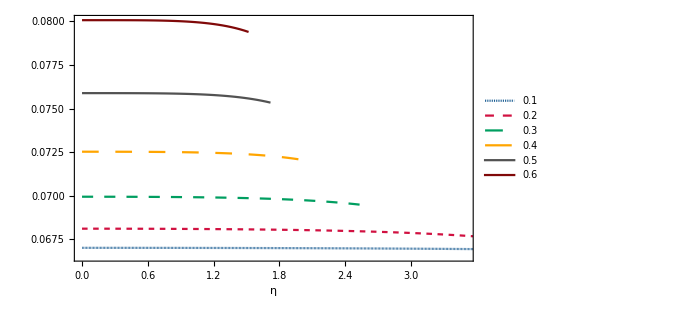

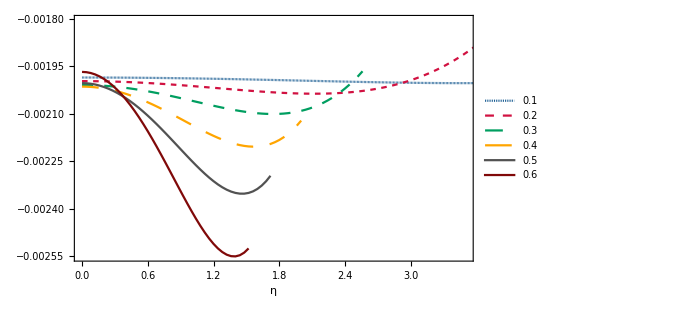

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/(0.2*Re[Td0][[k]][[j+1]][[1]])*100+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/(0.2*Abs[Im[Td0][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

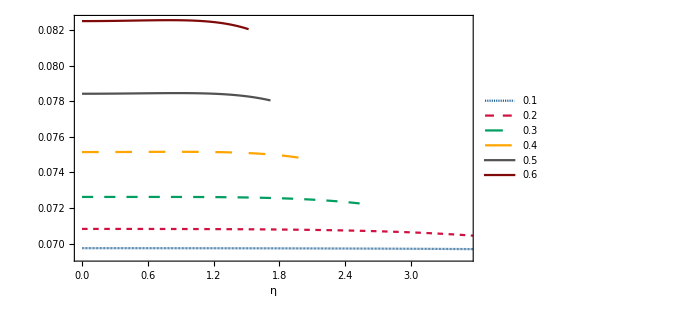

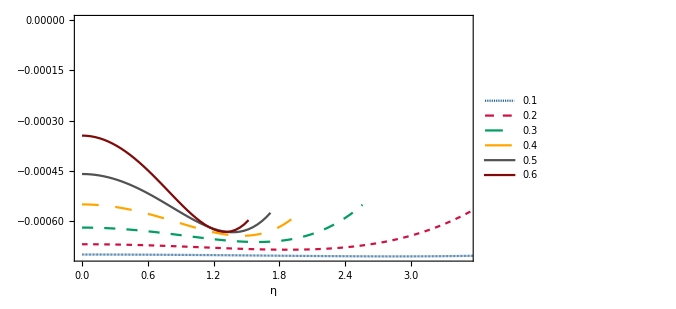

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

## L=2 electromagnetic modes

NOTE: I have used at=0.2 and m=1

### Axial modes

#### Slow-rotation QNMs

```mathematica
T1={{{0,0.4736557004414479-0.09494707247494184 ⅈ},{1/25+ⅈ/25,0.47365569349203124-0.09494706998100991 ⅈ},{2/25+(2 ⅈ)/25,0.4736556726486872-0.0949470625024851 ⅈ},{3/25+(3 ⅈ)/25,0.47365563792621684-0.0949470500492032 ⅈ},{4/25+(4 ⅈ)/25,0.47365558934927526-0.09494703263755207 ⅈ},{1/5+ⅈ/5,0.47365552695238106-0.0949470102904723 ⅈ},{6/25+(6 ⅈ)/25,0.47365545077991816-0.09494698303745443 ⅈ},{7/25+(7 ⅈ)/25,0.47365536088613686-0.09494695091453603 ⅈ},{8/25+(8 ⅈ)/25,0.4736552573351572-0.09494691396429757 ⅈ},{9/25+(9 ⅈ)/25,0.4736551402009709-0.09494687223585768 ⅈ},{2/5+(2 ⅈ)/5,0.47365500956744483-0.09494682578486784 ⅈ},{11/25+(11 ⅈ)/25,0.47365486552832453-0.09494677467350632 ⅈ},{12/25+(12 ⅈ)/25,0.4736547081872385-0.09494671897047101 ⅈ},{13/25+(13 ⅈ)/25,0.47365453765770177-0.09494665875097223 ⅈ},{14/25+(14 ⅈ)/25,0.4736543540631218-0.09494659409672411 ⅈ},{3/5+(3 ⅈ)/5,0.4736541575368029-0.09494652509593551 ⅈ},{16/25+(16 ⅈ)/25,0.4736539482219521-0.09494645184330047 ⅈ},{17/25+(17 ⅈ)/25,0.4736537262716852-0.09494637443998742 ⅈ},{18/25+(18 ⅈ)/25,0.4736534918490334-0.09494629299362801 ⅈ},{19/25+(19 ⅈ)/25,0.47365324512694973-0.09494620761830498 ⅈ},{4/5+(4 ⅈ)/5,0.47365298628831654-0.09494611843453947 ⅈ},{21/25+(21 ⅈ)/25,0.4736527155259534-0.09494602556927725 ⅈ},{22/25+(22 ⅈ)/25,0.4736524330426245-0.09494592915587478 ⅈ},{23/25+(23 ⅈ)/25,0.47365213905104747-0.09494582933408367 ⅈ},{24/25+(24 ⅈ)/25,0.4736518337739021-0.09494572625003529 ⅈ},{1+ⅈ,0.47365151744383954-0.0949456200562236 ⅈ},{26/25+(26 ⅈ)/25,0.47365119030349195-0.09494551091148834 ⅈ},{27/25+(27 ⅈ)/25,0.4736508526054822-0.0949453989809962 ⅈ},{28/25+(28 ⅈ)/25,0.4736505046124339-0.0949452844362224 ⅈ},{29/25+(29 ⅈ)/25,0.4736501465969833-0.09494516745493052 ⅈ},{6/5+(6 ⅈ)/5,0.47364977884178855-0.09494504822115199 ⅈ},{31/25+(31 ⅈ)/25,0.4736494016395426-0.09494492692516467 ⅈ},{32/25+(32 ⅈ)/25,0.47364901529298387-0.0949448037634707 ⅈ},{33/25+(33 ⅈ)/25,0.4736486201149088-0.09494467893877336 ⅈ},{34/25+(34 ⅈ)/25,0.47364821642818444-0.09494455265995314 ⅈ},{7/5+(7 ⅈ)/5,0.47364780456576083-0.09494442514204306 ⅈ},{36/25+(36 ⅈ)/25,0.4736473848706837-0.09494429660620317 ⅈ},{37/25+(37 ⅈ)/25,0.4736469576961089-0.09494416727969396 ⅈ},{38/25+(38 ⅈ)/25,0.47364652340531527-0.09494403739584908 ⅈ},{39/25+(39 ⅈ)/25,0.4736460823717188-0.09494390719404731 ⅈ},{8/5+(8 ⅈ)/5,0.4736456349788871-0.09494377691968338 ⅈ},{41/25+(41 ⅈ)/25,0.47364518162055363-0.09494364682413807 ⅈ},{42/25+(42 ⅈ)/25,0.47364472270063335-0.09494351716474728 ⅈ},{43/25+(43 ⅈ)/25,0.4736442586332368-0.09494338820477055 ⅈ},{44/25+(44 ⅈ)/25,0.4736437898426863-0.09494326021335805 ⅈ},{9/5+(9 ⅈ)/5,0.4736433167635315-0.09494313346551723 ⅈ},{46/25+(46 ⅈ)/25,0.473642839840565-0.09494300824207834 ⅈ},{47/25+(47 ⅈ)/25,0.47364235952883904-0.0949428848296587 ⅈ},{48/25+(48 ⅈ)/25,0.4736418762936813-0.09494276352062665 ⅈ},{49/25+(49 ⅈ)/25,0.47364139061071203-0.0949426446130638 ⅈ},{2+2 ⅈ,0.47364090296586076-0.094942528410727 ⅈ},{51/25+(51 ⅈ)/25,0.47364041385538297-0.09494241522300882 ⅈ},{52/25+(52 ⅈ)/25,0.47363992378587827-0.09494230536489726 ⅈ},{53/25+(53 ⅈ)/25,0.47363943327430674-0.09494219915693444 ⅈ},{54/25+(54 ⅈ)/25,0.4736389428480074-0.09494209692517422 ⅈ},{11/5+(11 ⅈ)/5,0.47363845304471525-0.09494199900113885 ⅈ},{56/25+(56 ⅈ)/25,0.47363796441258-0.09494190572177463 ⅈ},{57/25+(57 ⅈ)/25,0.47363747751018354-0.09494181742940616 ⅈ},{58/25+(58 ⅈ)/25,0.4736369929065581-0.09494173447169023 ⅈ},{59/25+(59 ⅈ)/25,0.47363651118120514-0.09494165720156791 ⅈ},{12/5+(12 ⅈ)/5,0.473636032924113-0.09494158597721591 ⅈ},{61/25+(61 ⅈ)/25,0.4736355587357759-0.09494152116199704 ⅈ},{62/25+(62 ⅈ)/25,0.4736350892272125-0.09494146312440903 ⅈ},{63/25+(63 ⅈ)/25,0.47363462501998405-0.09494141223803261 ⅈ},{64/25+(64 ⅈ)/25,0.47363416674621384-0.09494136888147864 ⅈ},{13/5+(13 ⅈ)/5,0.473633715048605-0.09494133343833336 ⅈ},{66/25+(66 ⅈ)/25,0.4736332705804603-0.09494130629710337 ⅈ},{67/25+(67 ⅈ)/25,0.47363283400569955-0.09494128785115893 ⅈ},{68/25+(68 ⅈ)/25,0.4736324059988797-0.09494127849867598 ⅈ},{69/25+(69 ⅈ)/25,0.47363198724521244-0.09494127864257747 ⅈ},{14/5+(14 ⅈ)/5,0.4736315784405835-0.0949412886904729 ⅈ},{71/25+(71 ⅈ)/25,0.473631180291571-0.0949413090545972 ⅈ},{72/25+(72 ⅈ)/25,0.47363079351546356-0.09494134015174797 ⅈ},{73/25+(73 ⅈ)/25,0.4736304188402795-0.09494138240322159 ⅈ},{74/25+(74 ⅈ)/25,0.4736300570047845-0.0949414362347481 ⅈ},{3+3 ⅈ,0.4736297087585099-0.09494150207642496 ⅈ},{76/25+(76 ⅈ)/25,0.47362937486177065-0.0949415803626492 ⅈ},{77/25+(77 ⅈ)/25,0.4736290560856834-0.09494167153204862 ⅈ},{78/25+(78 ⅈ)/25,0.4736287532121836-0.09494177602741136 ⅈ},{79/25+(79 ⅈ)/25,0.47362846703404343-0.09494189429561453 ⅈ},{16/5+(16 ⅈ)/5,0.4736281983548885-0.09494202678755118 ⅈ},{81/25+(81 ⅈ)/25,0.47362794798921526-0.0949421739580559 ⅈ},{82/25+(82 ⅈ)/25,0.47362771676240717-0.09494233626582957 ⅈ},{83/25+(83 ⅈ)/25,0.4736275055107511-0.09494251417336211 ⅈ},{84/25+(84 ⅈ)/25,0.4736273150814537-0.09494270814685422 ⅈ},{17/5+(17 ⅈ)/5,0.4736271463326568-0.09494291865613765 ⅈ},{86/25+(86 ⅈ)/25,0.47362700013345244-0.09494314617459401 ⅈ},{87/25+(87 ⅈ)/25,0.47362687736389825-0.09494339117907225 ⅈ},{88/25+(88 ⅈ)/25,0.47362677891503147-0.09494365414980478 ⅈ},{89/25+(89 ⅈ)/25,0.47362670568888354-0.09494393557032173 ⅈ},{18/5+(18 ⅈ)/5,0.4736266585984928-0.09494423592736446 ⅈ},{91/25+(91 ⅈ)/25,0.4736266385679184-0.09494455571079702 ⅈ},{92/25+(92 ⅈ)/25,0.4736266465322523-0.0949448954135163 ⅈ},{93/25+(93 ⅈ)/25,0.4736266834376314-0.09494525553136098 ⅈ},{94/25+(94 ⅈ)/25,0.47362675024124895-0.09494563656301849 ⅈ},{19/5+(19 ⅈ)/5,0.4736268479113653-0.09494603900993093 ⅈ},{96/25+(96 ⅈ)/25,0.47362697742731796-0.09494646337619915 ⅈ},{97/25+(97 ⅈ)/25,0.4736271397795312-0.0949469101684855 ⅈ},{98/25+(98 ⅈ)/25,0.47362733596952483-0.09494737989591508 ⅈ},{99/25+(99 ⅈ)/25,0.473627567009922-0.09494787306997508 ⅈ},{4+4 ⅈ,0.47362783392445673-0.0949483902044132 ⅈ},{101/25+(101 ⅈ)/25,0.47362813774798046-0.09494893181513386 ⅈ},{102/25+(102 ⅈ)/25,0.47362847952646736-0.09494949842009336 ⅈ},{103/25+(103 ⅈ)/25,0.4736288603170195-0.09495009053919315 ⅈ},{104/25+(104 ⅈ)/25,0.4736292811878704-0.09495070869417156 ⅈ},{21/5+(21 ⅈ)/5,0.4736297432183883-0.09495135340849421 ⅈ},{106/25+(106 ⅈ)/25,0.47363024749907806-0.0949520252072424 ⅈ},{107/25+(107 ⅈ)/25,0.4736307951315823-0.09495272461700027 ⅈ},{108/25+(108 ⅈ)/25,0.47363138722868103-0.09495345216574017 ⅈ},{109/25+(109 ⅈ)/25,0.4736320249142912-0.09495420838270642 ⅈ},{22/5+(22 ⅈ)/5,0.47363270932346346-0.09495499379829753 ⅈ},{111/25+(111 ⅈ)/25,0.4736334416023802-0.09495580894394681 ⅈ},{112/25+(112 ⅈ)/25,0.4736342229083497-0.09495665435200132 ⅈ},{113/25+(113 ⅈ)/25,0.47363505440980136-0.09495753055559904 ⅈ},{114/25+(114 ⅈ)/25,0.47363593728627823-0.09495843808854482 ⅈ},{23/5+(23 ⅈ)/5,0.47363687272842864-0.09495937748518422 ⅈ},{116/25+(116 ⅈ)/25,0.4736378619379967-0.09496034928027619 ⅈ},{117/25+(117 ⅈ)/25,0.4736389061278113-0.09496135400886384 ⅈ},{118/25+(118 ⅈ)/25,0.4736400065217734-0.09496239220614341 ⅈ},{119/25+(119 ⅈ)/25,0.4736411643548428-0.09496346440733217 ⅈ},{24/5+(24 ⅈ)/5,0.47364238087302135-0.09496457114753425 ⅈ},{121/25+(121 ⅈ)/25,0.4736436573333374-0.09496571296160494 ⅈ},{122/25+(122 ⅈ)/25,0.4736449950038262-0.09496689038401351 ⅈ},{123/25+(123 ⅈ)/25,0.4736463951635102-0.09496810394870428 ⅈ},{124/25+(124 ⅈ)/25,0.47364785910237694-0.0949693541889561 ⅈ},{5+5 ⅈ,0.47364938812135493-0.09497064163724048 ⅈ},{126/25+(126 ⅈ)/25,0.4736509835322892-0.09497196682507761 ⅈ},{127/25+(127 ⅈ)/25,0.47365264665791323-0.09497333028289151 ⅈ},{128/25+(128 ⅈ)/25,0.47365437883182-0.09497473253986287 ⅈ},{129/25+(129 ⅈ)/25,0.4736561813984308-0.09497617412378082 ⅈ},{26/5+(26 ⅈ)/5,0.4736580557129627-0.0949776555608933 ⅈ},{131/25+(131 ⅈ)/25,0.4736600031413929-0.09497917737575504 ⅈ},{132/25+(132 ⅈ)/25,0.4736620250604217-0.09498074009107522 ⅈ},{133/25+(133 ⅈ)/25,0.4736641228574338-0.0949823442275626 ⅈ},{134/25+(134 ⅈ)/25,0.4736662979304561-0.0949839903037698 ⅈ},{27/5+(27 ⅈ)/5,0.473668551688115-0.09498567883593573 ⅈ},{136/25+(136 ⅈ)/25,0.4736708855495894-0.09498741033782687 ⅈ},{137/25+(137 ⅈ)/25,0.47367330094456356-0.09498918532057704 ⅈ},{138/25+(138 ⅈ)/25,0.47367579931317605-0.09499100429252541 ⅈ},{139/25+(139 ⅈ)/25,0.47367838210596674-0.0949928677590538 ⅈ},{28/5+(28 ⅈ)/5,0.47368105078382156-0.09499477622242196 ⅈ},{141/25+(141 ⅈ)/25,0.4736838068179145-0.09499673018160205 ⅈ},{142/25+(142 ⅈ)/25,0.4736866516896468-0.09499873013211141 ⅈ},{143/25+(143 ⅈ)/25,0.4736895868905845-0.09500077656584419 ⅈ},{144/25+(144 ⅈ)/25,0.47369261392239176-0.09500286997090186 ⅈ},{29/5+(29 ⅈ)/5,0.47369573429676276-0.09500501083142239 ⅈ},{146/25+(146 ⅈ)/25,0.4736989495353506-0.0950071996274084 ⅈ},{147/25+(147 ⅈ)/25,0.4737022611696928-0.09500943683455357 ⅈ},{148/25+(148 ⅈ)/25,0.47370567074113423-0.09501172292406881 ⅈ},{149/25+(149 ⅈ)/25,0.4737091798007475-0.09501405836250706 ⅈ},{6+6 ⅈ,0.4737127899092498-0.09501644361158641 ⅈ},{151/25+(151 ⅈ)/25,0.4737165026369168-0.0950188791280134 ⅈ},{152/25+(152 ⅈ)/25,0.47372031956349386-0.09502136536330408 ⅈ},{153/25+(153 ⅈ)/25,0.47372424227810345-0.09502390276360545 ⅈ},{154/25+(154 ⅈ)/25,0.47372827237915055-0.09502649176951507 ⅈ},{31/5+(31 ⅈ)/5,0.47373241147422296-0.09502913281590011 ⅈ},{156/25+(156 ⅈ)/25,0.4737366611799902-0.09503182633171628 ⅈ},{157/25+(157 ⅈ)/25,0.47374102312209765-0.09503457273982499 ⅈ},{158/25+(158 ⅈ)/25,0.4737454989350587-0.09503737245681057 ⅈ},{159/25+(159 ⅈ)/25,0.4737500902621418-0.09504022589279655 ⅈ},{32/5+(32 ⅈ)/5,0.47375479875525545-0.09504313345126204 ⅈ},{161/25+(161 ⅈ)/25,0.47375962607482974-0.09504609552885854 ⅈ},{162/25+(162 ⅈ)/25,0.47376457388969057-0.095049112515218 ⅈ},{163/25+(163 ⅈ)/25,0.4737696438769373-0.0950521847927808 ⅈ},{164/25+(164 ⅈ)/25,0.47377483772181234-0.09505531273659484 ⅈ},{33/5+(33 ⅈ)/5,0.47378015711756455-0.09505849671414175 ⅈ},{166/25+(166 ⅈ)/25,0.473785603765314-0.09506173708514429 ⅈ},{167/25+(167 ⅈ)/25,0.47379117937391-0.09506503420138251 ⅈ},{168/25+(168 ⅈ)/25,0.47379688565978684-0.09506838840650811 ⅈ},{169/25+(169 ⅈ)/25,0.4738027243468145-0.09507180003585702 ⅈ},{34/5+(34 ⅈ)/5,0.47380869716614477-0.0950752694162651 ⅈ},{171/25+(171 ⅈ)/25,0.4738148058560557-0.09507879686588115 ⅈ},{172/25+(172 ⅈ)/25,0.4738210521617905-0.09508238269398306 ⅈ},{173/25+(173 ⅈ)/25,0.47382743783539283-0.09508602720079166 ⅈ},{174/25+(174 ⅈ)/25,0.47383396463553595-0.09508973067728758 ⅈ},{7+7 ⅈ,0.47384063432735457-0.09509349340502574 ⅈ},{176/25+(176 ⅈ)/25,0.473847448682261-0.09509731565595396 ⅈ},{177/25+(177 ⅈ)/25,0.47385440947776936-0.09510119769222929 ⅈ},{178/25+(178 ⅈ)/25,0.4738615184973084-0.09510513976603802 ⅈ}},{{0,0.4777957245356762-0.09521452729967887 ⅈ},{1/25+ⅈ/25,0.4777957104220658-0.09521451281664045 ⅈ},{2/25+(2 ⅈ)/25,0.47779566815524094-0.09521446941567989 ⅈ},{3/25+(3 ⅈ)/25,0.4777955979573724-0.09521439724138431 ⅈ},{4/25+(4 ⅈ)/25,0.47779550019876-0.09521429653463478 ⅈ},{1/5+ⅈ/5,0.4777953753979031-0.09521416763251082 ⅈ},{6/25+(6 ⅈ)/25,0.47779522422158116-0.09521401096813617 ⅈ},{7/25+(7 ⅈ)/25,0.47779504748495605-0.0952138270704802 ⅈ},{8/25+(8 ⅈ)/25,0.4777948461516968-0.09521361656411469 ⅈ},{9/25+(9 ⅈ)/25,0.47779462133412676-0.09521338016892567 ⅈ},{2/5+(2 ⅈ)/5,0.4777943742933926-0.09521311869977997 ⅈ},{11/25+(11 ⅈ)/25,0.47779410643965503-0.09521283306614607 ⅈ},{12/25+(12 ⅈ)/25,0.47779381933230036-0.0952125242716687 ⅈ},{13/25+(13 ⅈ)/25,0.4777935146801732-0.0952121934136972 ⅈ},{14/25+(14 ⅈ)/25,0.4777931943418296-0.09521184168276595 ⅈ},{3/5+(3 ⅈ)/5,0.47779286032581-0.09521147036202755 ⅈ},{16/25+(16 ⅈ)/25,0.477792514790931-0.09521108082663739 ⅈ},{17/25+(17 ⅈ)/25,0.4777921600465966-0.09521067454308867 ⅈ},{18/25+(18 ⅈ)/25,0.4777917985531277-0.09521025306849783 ⅈ},{19/25+(19 ⅈ)/25,0.47779143292210785-0.09520981804983891 ⅈ},{4/5+(4 ⅈ)/5,0.4777910659167467-0.09520937122312649 ⅈ},{21/25+(21 ⅈ)/25,0.4777907004522591-0.09520891441254589 ⅈ},{22/25+(22 ⅈ)/25,0.4777903395962582-0.09520844952952986 ⅈ},{23/25+(23 ⅈ)/25,0.47778998656916477-0.09520797857178093 ⅈ},{24/25+(24 ⅈ)/25,0.4777896447446269-0.09520750362223801 ⅈ},{1+ⅈ,0.4777893176499537-0.09520702684798663 ⅈ},{26/25+(26 ⅈ)/25,0.4777890089665588-0.09520655049911113 ⅈ},{27/25+(27 ⅈ)/25,0.47778872253041427-0.09520607690748852 ⅈ},{28/25+(28 ⅈ)/25,0.4777884623325126-0.09520560848552158 ⅈ},{29/25+(29 ⅈ)/25,0.47778823251933533-0.0952051477248112 ⅈ},{6/5+(6 ⅈ)/5,0.47778803739332865-0.09520469719476618 ⅈ},{31/25+(31 ⅈ)/25,0.477787881413382-0.09520425954114908 ⅈ},{32/25+(32 ⅈ)/25,0.4777877691953098-0.09520383748455692 ⅈ},{33/25+(33 ⅈ)/25,0.47778770551233457-0.09520343381883582 ⅈ},{34/25+(34 ⅈ)/25,0.4777876952955683-0.09520305140942756 ⅈ},{7/5+(7 ⅈ)/5,0.47778774363449283-0.09520269319164723 ⅈ},{36/25+(36 ⅈ)/25,0.4777878557774343-0.09520236216889036 ⅈ},{37/25+(37 ⅈ)/25,0.47778803713203205-0.0952020614107683 ⅈ},{38/25+(38 ⅈ)/25,0.47778829326569866-0.09520179405117025 ⅈ},{39/25+(39 ⅈ)/25,0.4777886299060692-0.09520156328625091 ⅈ},{8/5+(8 ⅈ)/5,0.47778905294143786-0.09520137237234194 ⅈ},{41/25+(41 ⅈ)/25,0.47778956842117837-0.09520122462378616 ⅈ},{42/25+(42 ⅈ)/25,0.4777901825561472-0.0952011234106934 ⅈ},{43/25+(43 ⅈ)/25,0.47779090171906574-0.09520107215661572 ⅈ},{44/25+(44 ⅈ)/25,0.47779173244487927-0.09520107433614196 ⅈ},{9/5+(9 ⅈ)/5,0.47779268143108977-0.09520113347240929 ⅈ},{46/25+(46 ⅈ)/25,0.47779375553805925-0.09520125313453104 ⅈ},{47/25+(47 ⅈ)/25,0.4777949617892817-0.09520143693493967 ⅈ},{48/25+(48 ⅈ)/25,0.4777963073716181-0.09520168852664339 ⅈ},{49/25+(49 ⅈ)/25,0.47779779963549457-0.09520201160039571 ⅈ},{2+2 ⅈ,0.47779944609505615-0.09520240988177643 ⅈ},{51/25+(51 ⅈ)/25,0.4778012544282761-0.09520288712818392 ⅈ},{52/25+(52 ⅈ)/25,0.4778032324770158-0.09520344712573695 ⅈ},{53/25+(53 ⅈ)/25,0.47780538824702967-0.09520409368608573 ⅈ},{54/25+(54 ⅈ)/25,0.47780772990791437-0.09520483064313184 ⅈ},{11/5+(11 ⅈ)/5,0.4778102657929954-0.09520566184965536 ⅈ},{56/25+(56 ⅈ)/25,0.47781300439914826-0.09520659117385041 ⅈ},{57/25+(57 ⅈ)/25,0.4778159543865498-0.0952076224957671 ⅈ},{58/25+(58 ⅈ)/25,0.47781912457835385-0.09520875970366098 ⅈ},{59/25+(59 ⅈ)/25,0.47782252396028924-0.09521000669024939 ⅈ},{12/5+(12 ⅈ)/5,0.47782616168017167-0.09521136734887492 ⅈ},{61/25+(61 ⅈ)/25,0.47783004704732857-0.09521284556957621 ⅈ},{62/25+(62 ⅈ)/25,0.47783418953192897-0.09521444523506718 ⅈ},{63/25+(63 ⅈ)/25,0.47783859876421403-0.09521617021662448 ⅈ},{64/25+(64 ⅈ)/25,0.47784328453362485-0.09521802436988482 ⅈ},{13/5+(13 ⅈ)/5,0.4778482567878182-0.09522001153055305 ⅈ},{66/25+(66 ⅈ)/25,0.4778535256315696-0.09522213551002219 ⅈ},{67/25+(67 ⅈ)/25,0.47785910132555426-0.09522440009090756 ⅈ},{68/25+(68 ⅈ)/25,0.4778649942850021-0.09522680902249629 ⅈ},{69/25+(69 ⅈ)/25,0.47787121507822133-0.09522936601611491 ⅈ},{14/5+(14 ⅈ)/5,0.4778777744249836-0.09523207474041712 ⅈ},{71/25+(71 ⅈ)/25,0.47788468319476585-0.09523493881659476 ⅈ},{72/25+(72 ⅈ)/25,0.4778919524048433-0.09523796181351488 ⅈ},{73/25+(73 ⅈ)/25,0.4778995932182262-0.09524114724278658 ⅈ},{74/25+(74 ⅈ)/25,0.47790761694143646-0.09524449855376124 ⅈ},{3+3 ⅈ,0.47791603502211544-0.09524801912847015 ⅈ},{76/25+(76 ⅈ)/25,0.4779248590464612-0.09525171227650425 ⅈ},{77/25+(77 ⅈ)/25,0.4779341007364841-0.0952555812298411 ⅈ},{78/25+(78 ⅈ)/25,0.47794377194707965-0.09525962913762374 ⅈ},{79/25+(79 ⅈ)/25,0.47795388466290983-0.09526385906089745 ⅈ},{16/5+(16 ⅈ)/5,0.4779644509950889-0.09526827396731113 ⅈ},{81/25+(81 ⅈ)/25,0.477975483177667-0.0952728767257885 ⅈ},{82/25+(82 ⅈ)/25,0.4779869935639071-0.0952776701011776 ⅈ},{83/25+(83 ⅈ)/25,0.47799899462234924-0.0952826567488845 ⅈ},{84/25+(84 ⅈ)/25,0.4780114989326585-0.0952878392095023 ⅈ},{17/5+(17 ⅈ)/5,0.4780245191812487-0.095293219903436 ⅈ},{86/25+(86 ⅈ)/25,0.47803806815668287-0.09529880112554409 ⅈ},{87/25+(87 ⅈ)/25,0.4780521587448393-0.09530458503979476 ⅈ},{88/25+(88 ⅈ)/25,0.47806680392384604-0.09531057367395329 ⅈ},{89/25+(89 ⅈ)/25,0.47808201675877393-0.09531676891430665 ⅈ},{18/5+(18 ⅈ)/5,0.47809781039609117-0.09532317250044042 ⅈ},{91/25+(91 ⅈ)/25,0.47811419805787225-0.09532978602007425 ⅈ}},{{0,0.4845094275670288-0.09564863991847104 ⅈ},{1/25+ⅈ/25,0.4845094423143905-0.09564859141728019 ⅈ},{2/25+(2 ⅈ)/25,0.4845094868938677-0.09564844612573405 ⅈ},{3/25+(3 ⅈ)/25,0.4845095623175863-0.09564820468016534 ⅈ},{4/25+(4 ⅈ)/25,0.48450967027277264-0.09564786814027637 ⅈ},{1/5+ⅈ/5,0.4845098131222243-0.09564743798802823 ⅈ},{6/25+(6 ⅈ)/25,0.4845099939049873-0.09564691612601392 ⅈ},{7/25+(7 ⅈ)/25,0.4845102163372197-0.09564630487535969 ⅈ},{8/25+(8 ⅈ)/25,0.4845104848132393-0.09564560697314967 ⅈ},{9/25+(9 ⅈ)/25,0.48451080440674826-0.09564482556936733 ⅈ},{2/5+(2 ⅈ)/5,0.48451118087222866-0.09564396422334694 ⅈ},{11/25+(11 ⅈ)/25,0.48451162064650166-0.09564302689972555 ⅈ},{12/25+(12 ⅈ)/25,0.48451213085044065-0.09564201796388802 ⅈ},{13/25+(13 ⅈ)/25,0.48451271929082956-0.09564094217689201 ⅈ},{14/25+(14 ⅈ)/25,0.4845133944623537-0.09563980468986413 ⅈ},{3/5+(3 ⅈ)/5,0.48451416554971233-0.09563861103785301 ⅈ},{16/25+(16 ⅈ)/25,0.48451504242983773-0.0956373671331269 ⅈ},{17/25+(17 ⅈ)/25,0.4845160356742062-0.09563607925790145 ⅈ},{18/25+(18 ⅈ)/25,0.4845171565512245-0.0956347540564828 ⅈ},{19/25+(19 ⅈ)/25,0.48451841702867343-0.09563339852681009 ⅈ},{4/5+(4 ⅈ)/5,0.48451982977618824-0.09563202001138159 ⅈ},{21/25+(21 ⅈ)/25,0.48452140816775624-0.09563062618754685 ⅈ},{22/25+(22 ⅈ)/25,0.4845231662842057-0.09562922505714824 ⅈ},{23/25+(23 ⅈ)/25,0.48452511891566347-0.09562782493549335 ⅈ},{24/25+(24 ⅈ)/25,0.48452728156395386-0.09562643443964039 ⅈ},{1+ⅈ,0.4845296704449086-0.09562506247597881 ⅈ},{26/25+(26 ⅈ)/25,0.4845323024905596-0.09562371822708249 ⅈ},{27/25+(27 ⅈ)/25,0.48453519535117645-0.0956224111378402 ⅈ},{28/25+(28 ⅈ)/25,0.4845383673971236-0.09562115090077902 ⅈ},{29/25+(29 ⅈ)/25,0.4845418377204833-0.09561994744067237 ⅈ},{6/5+(6 ⅈ)/5,0.48454562613642177-0.09561881089830654 ⅈ},{31/25+(31 ⅈ)/25,0.48454975318424365-0.09561775161345437 ⅈ},{32/25+(32 ⅈ)/25,0.4845542401280951-0.09561678010701939 ⅈ},{33/25+(33 ⅈ)/25,0.48455910895726795-0.09561590706233863 ⅈ},{34/25+(34 ⅈ)/25,0.48456438238605093-0.09561514330563194 ⅈ},{7/5+(7 ⅈ)/5,0.4845700838530803-0.09561449978558575 ⅈ},{36/25+(36 ⅈ)/25,0.48457623752012946-0.0956139875520631 ⅈ},{37/25+(37 ⅈ)/25,0.4845828682702818-0.09561361773393177 ⅈ},{38/25+(38 ⅈ)/25,0.4845900017054241-0.09561340151600715 ⅈ},{39/25+(39 ⅈ)/25,0.4845976641429978-0.09561335011510728 ⅈ},{8/5+(8 ⅈ)/5,0.48460588261194004-0.09561347475522222 ⅈ},{41/25+(41 ⅈ)/25,0.4846146848477461-0.09561378664180255 ⅈ},{42/25+(42 ⅈ)/25,0.48462409928658146-0.09561429693517648 ⅈ},{43/25+(43 ⅈ)/25,0.48463415505836815-0.09561501672310845 ⅈ},{44/25+(44 ⅈ)/25,0.48464488197877-0.09561595699251788 ⅈ},{9/5+(9 ⅈ)/5,0.48465631053999786-0.09561712860038063 ⅈ},{46/25+(46 ⅈ)/25,0.48466847190035334-0.09561854224384324 ⅈ},{47/25+(47 ⅈ)/25,0.48468139787243075-0.09562020842958308 ⅈ},{48/25+(48 ⅈ)/25,0.4846951209098924-0.09562213744245711 ⅈ},{49/25+(49 ⅈ)/25,0.4847096740927337-0.09562433931348695 ⅈ},{2+2 ⅈ,0.4847250911109535-0.09562682378723526 ⅈ},{51/25+(51 ⅈ)/25,0.48474140624654466-0.09562960028863737 ⅈ},{52/25+(52 ⅈ)/25,0.4847586543537214-0.09563267788935827 ⅈ},{53/25+(53 ⅈ)/25,0.48477687083729964-0.09563606527375666 ⅈ},{54/25+(54 ⅈ)/25,0.4847960916291504-0.09563977070454212 ⅈ},{11/5+(11 ⅈ)/5,0.4848163531626471-0.09564380198822602 ⅈ},{56/25+(56 ⅈ)/25,0.4848376923450317-0.0956481664404712 ⅈ},{57/25+(57 ⅈ)/25,0.4848601465276294-0.09565287085145814 ⅈ},{58/25+(58 ⅈ)/25,0.48488375347384655-0.09565792145139662 ⅈ},{59/25+(59 ⅈ)/25,0.48490855132488914-0.09566332387631503 ⅈ},{12/5+(12 ⅈ)/5,0.4849345785631612-0.09566908313427394 ⅈ},{61/25+(61 ⅈ)/25,0.48496187397327406-0.0956752035721764 ⅈ},{62/25+(62 ⅈ)/25,0.48499047660066136-0.09568168884330569 ⅈ},{63/25+(63 ⅈ)/25,0.48502042570779164-0.09568854187581433 ⅈ},{64/25+(64 ⅈ)/25,0.4850517607278632-0.0956957648422943 ⅈ}},{{0,0.4935703733928563-0.0962359111215069 ⅈ},{1/25+ⅈ/25,0.49357050164151994-0.09623578877763125 ⅈ},{2/25+(2 ⅈ)/25,0.4935708873070905-0.09623542229624846 ⅈ},{3/25+(3 ⅈ)/25,0.4935715331473681-0.09623481332815348 ⅈ},{4/25+(4 ⅈ)/25,0.4935724437600406-0.0962339646205917 ⅈ},{1/5+ⅈ/5,0.4935736255842498-0.09623288001155288 ⅈ},{6/25+(6 ⅈ)/25,0.4935750869029341-0.09623156442158112 ⅈ},{7/25+(7 ⅈ)/25,0.49357683784578704-0.09623002384319289 ⅈ},{8/25+(8 ⅈ)/25,0.49357889039279007-0.09622826532786538 ⅈ},{9/25+(9 ⅈ)/25,0.49358125837827393-0.09622629697054834 ⅈ},{2/5+(2 ⅈ)/5,0.493583957495443-0.09622412789164533 ⅈ},{11/25+(11 ⅈ)/25,0.4935870053012957-0.09622176821640331 ⅈ},{12/25+(12 ⅈ)/25,0.49359042122186025-0.09621922905164115 ⅈ},{13/25+(13 ⅈ)/25,0.49359422655765023-0.09621652245974355 ⅈ},{14/25+(14 ⅈ)/25,0.4935984444892373-0.09621366142983788 ⅈ},{3/5+(3 ⅈ)/5,0.4936031000828234-0.0962106598460695 ⅈ},{16/25+(16 ⅈ)/25,0.49360822029568074-0.09620753245288408 ⅈ},{17/25+(17 ⅈ)/25,0.49361383398131575-0.09620429481722383 ⅈ},{18/25+(18 ⅈ)/25,0.49361997189419515-0.09620096328754062 ⅈ},{19/25+(19 ⅈ)/25,0.4936266666938612-0.09619755494952917 ⅈ},{4/5+(4 ⅈ)/5,0.4936339529482414-0.09619408757848183 ⅈ},{21/25+(21 ⅈ)/25,0.49364186713594405-0.09619057958816934 ⅈ},{22/25+(22 ⅈ)/25,0.4936504476473126-0.0961870499761545 ⅈ},{23/25+(23 ⅈ)/25,0.49365973478399183-0.0961835182654502 ⅈ},{24/25+(24 ⅈ)/25,0.4936697707567385-0.09618000444244108 ⅈ},{1+ⅈ,0.49368059968119277-0.09617652889099647 ⅈ},{26/25+(26 ⅈ)/25,0.49369226757130036-0.09617311232271485 ⅈ},{27/25+(27 ⅈ)/25,0.4937048223300621-0.09616977570324871 ⅈ},{28/25+(28 ⅈ)/25,0.4937183137372511-0.09616654017469613 ⅈ},{29/25+(29 ⅈ)/25,0.4937327934337431-0.0961634269740245 ⅈ},{6/5+(6 ⅈ)/5,0.49374831490205207-0.09616045734756709 ⅈ},{31/25+(31 ⅈ)/25,0.49376493344266853-0.0961576524616192 ⅈ},{32/25+(32 ⅈ)/25,0.4937827061457655-0.09615503330921245 ⅈ},{33/25+(33 ⅈ)/25,0.4938016918578222-0.09615262061317441 ⅈ},{34/25+(34 ⅈ)/25,0.4938219511426975-0.09615043472562255 ⅈ},{7/5+(7 ⅈ)/5,0.49384354623667565-0.09614849552408175 ⅈ},{36/25+(36 ⅈ)/25,0.4938665409969864-0.09614682230446775 ⅈ},{37/25+(37 ⅈ)/25,0.49389100084330384-0.09614543367122659 ⅈ},{38/25+(38 ⅈ)/25,0.49391699269171574-0.09614434742498162 ⅈ},{39/25+(39 ⅈ)/25,0.49394458488066356-0.09614358044809714 ⅈ},{8/5+(8 ⅈ)/5,0.49397384708835385-0.09614314858863855 ⅈ},{41/25+(41 ⅈ)/25,0.49400485024115254-0.09614306654327859 ⅈ},{42/25+(42 ⅈ)/25,0.49403766641254876-0.0961433477397446 ⅈ},{43/25+(43 ⅈ)/25,0.49407236871213667-0.0961440042195683 ⅈ},{44/25+(44 ⅈ)/25,0.4941090311643785-0.09614504652182852 ⅈ},{9/5+(9 ⅈ)/5,0.49414772857669315-0.09614648356880448 ⅈ},{46/25+(46 ⅈ)/25,0.4941885363966316-0.09614832255445052 ⅈ},{47/25+(47 ⅈ)/25,0.49423153055792374-0.09615056883670875 ⅈ},{48/25+(48 ⅈ)/25,0.4942767873152732-0.09615322583475158 ⅈ},{49/25+(49 ⅈ)/25,0.49432438306787807-0.09615629493231276 ⅈ},{2+2 ⅈ,0.4943743941717643-0.09615977538833576 ⅈ}},{{0,0.5047345943230471-0.09696263631352511 ⅈ},{1/25+ⅈ/25,0.5047349734258626-0.09696238116238046 ⅈ},{2/25+(2 ⅈ)/25,0.5047361125832509-0.09696161674072006 ⅈ},{3/25+(3 ⅈ)/25,0.5047380173387902-0.09696034614257426 ⅈ},{4/25+(4 ⅈ)/25,0.5047406969341951-0.09695857451140898 ⅈ},{1/5+ⅈ/5,0.5047441643115372-0.09695630902107877 ⅈ},{6/25+(6 ⅈ)/25,0.5047484361167242-0.09695355884867862 ⅈ},{7/25+(7 ⅈ)/25,0.504753532703694-0.09695033513942633 ⅈ},{8/25+(8 ⅈ)/25,0.5047594781391195-0.09694665096341906 ⅈ},{9/25+(9 ⅈ)/25,0.5047663002073501-0.09694252126407688 ⅈ},{2/5+(2 ⅈ)/5,0.5047740304152853-0.09693796279805797 ⅈ},{11/25+(11 ⅈ)/25,0.5047827039968013-0.09693299406640535 ⅈ},{12/25+(12 ⅈ)/25,0.5047923599163003-0.09692763523666137 ⅈ},{13/25+(13 ⅈ)/25,0.5048030408708898-0.09692190805567255 ⅈ},{14/25+(14 ⅈ)/25,0.5048147932906261-0.09691583575279158 ⅈ},{3/5+(3 ⅈ)/5,0.5048276673361952-0.09690944293317971 ⅈ},{16/25+(16 ⅈ)/25,0.5048417168933206-0.09690275546091313 ⅈ},{17/25+(17 ⅈ)/25,0.5048569995631131-0.09689580033160577 ⅈ},{18/25+(18 ⅈ)/25,0.5048735766474974-0.09688860553427925 ⅈ},{19/25+(19 ⅈ)/25,0.5048915131287577-0.09688119990223955 ⅈ},{4/5+(4 ⅈ)/5,0.50491087764216-0.0968736129527607 ⅈ},{21/25+(21 ⅈ)/25,0.5049317424405171-0.09686587471542867 ⅈ},{22/25+(22 ⅈ)/25,0.5049541833494625-0.09685801554906787 ⅈ},{23/25+(23 ⅈ)/25,0.5049782797121134-0.09685006594725729 ⅈ},{24/25+(24 ⅈ)/25,0.5050041143217027-0.09684205633254624 ⅈ},{1+ⅈ,0.5050317733406711-0.09683401683960025 ⅈ},{26/25+(26 ⅈ)/25,0.5050613462046261-0.0968259770876624 ⅈ},{27/25+(27 ⅈ)/25,0.5050929255095054-0.09681796594281944 ⅈ},{28/25+(28 ⅈ)/25,0.5051266068801746-0.09681001127092671 ⅈ},{29/25+(29 ⅈ)/25,0.5051624888187076-0.09680213968197637 ⅈ},{6/5+(6 ⅈ)/5,0.5052006725304936-0.09679437626721052 ⅈ},{31/25+(31 ⅈ)/25,0.5052412617263432-0.09678674433038294 ⅈ},{32/25+(32 ⅈ)/25,0.5052843623987737-0.09677926511491647 ⅈ},{33/25+(33 ⅈ)/25,0.505330082570704-0.09677195752901017 ⅈ},{34/25+(34 ⅈ)/25,0.5053785320148864-0.09676483787108389 ⅈ},{7/5+(7 ⅈ)/5,0.5054298219425389-0.09675791955830293 ⅈ},{36/25+(36 ⅈ)/25,0.5054840646598409-0.09675121286129029 ⅈ},{37/25+(37 ⅈ)/25,0.5055413731912026-0.09674472464850872 ⅈ},{38/25+(38 ⅈ)/25,0.505601860868551-0.09673845814416464 ⅈ},{39/25+(39 ⅈ)/25,0.5056656408862598-0.0967324127038504 ⅈ},{8/5+(8 ⅈ)/5,0.5057328258218345-0.09672658361247632 ⅈ},{41/25+(41 ⅈ)/25,0.5058035271230128-0.0967209619093484 ⅈ},{42/25+(42 ⅈ)/25,0.5058778545625797-0.09671553424549591 ⅈ},{43/25+(43 ⅈ)/25,0.5059559156629231-0.09671028277853005 ⅈ}},{{0,0.5177684659125577-0.09781645372800081 ⅈ},{1/25+ⅈ/25,0.5177692865801191-0.09781599047906642 ⅈ},{2/25+(2 ⅈ)/25,0.5177717515754147-0.09781460222974639 ⅈ},{3/25+(3 ⅈ)/25,0.5177758698676191-0.09781229346740578 ⅈ},{4/25+(4 ⅈ)/25,0.5177816564051281-0.09780907163777124 ⅈ},{1/5+ⅈ/5,0.5177891321120506-0.09780494709656083 ⅈ},{6/25+(6 ⅈ)/25,0.5177983238838587-0.09779993304078148 ⅈ},{7/25+(7 ⅈ)/25,0.5178092645807814-0.09779404541983144 ⅈ},{8/25+(8 ⅈ)/25,0.5178219930181573-0.09778730282600194 ⅈ},{9/25+(9 ⅈ)/25,0.5178365539527906-0.09777972636390271 ⅈ},{2/5+(2 ⅈ)/5,0.5178529980641305-0.09777133949828004 ⅈ},{11/25+(11 ⅈ)/25,0.5178713819289077-0.09776216787965787 ⅈ},{12/25+(12 ⅈ)/25,0.51789176798762-0.09775223914721139 ⅈ},{13/25+(13 ⅈ)/25,0.5179142245010355-0.0977415827082894 ⅈ},{14/25+(14 ⅈ)/25,0.5179388254946242-0.0977302294940341 ⅈ},{3/5+(3 ⅈ)/5,0.5179656506885775-0.09771821169061337 ⅈ},{16/25+(16 ⅈ)/25,0.5179947854107911-0.09770556244569698 ⅈ},{17/25+(17 ⅈ)/25,0.5180263204899025-0.09769231554989788 ⅈ},{18/25+(18 ⅈ)/25,0.5180603521252151-0.09767850509326718 ⅈ},{19/25+(19 ⅈ)/25,0.518096981729988-0.09766416509692703 ⅈ},{4/5+(4 ⅈ)/5,0.5181363157443426-0.09764932912050076 ⅈ},{21/25+(21 ⅈ)/25,0.5181784654137203-0.09763402984624933 ⅈ},{22/25+(22 ⅈ)/25,0.5182235465285767-0.09761829864134196 ⅈ},{23/25+(23 ⅈ)/25,0.5182716791207715-0.09760216510024171 ⅈ},{24/25+(24 ⅈ)/25,0.5183229871119233-0.09758565656983516 ⅈ},{1+ⅈ,0.5183775979088826-0.09756879766067797 ⅈ},{26/25+(26 ⅈ)/25,0.5184356419414354-0.09755160974857019 ⅈ},{27/25+(27 ⅈ)/25,0.5184972521374117-0.09753411047161123 ⅈ},{28/25+(28 ⅈ)/25,0.5185625633305706-0.097516313228913 ⅈ},{29/25+(29 ⅈ)/25,0.5186317115969871-0.0974982266882641 ⅈ},{6/5+(6 ⅈ)/5,0.5187048335161991-0.09747985431121725 ⅈ},{31/25+(31 ⅈ)/25,0.5187820653541446-0.09746119390530052 ⅈ},{32/25+(32 ⅈ)/25,0.5188635421659179-0.09744223721429693 ⅈ},{33/25+(33 ⅈ)/25,0.5189493968176762-0.09742296955875812 ⅈ},{34/25+(34 ⅈ)/25,0.519039758928628-0.09740336954006394 ⅈ},{7/5+(7 ⅈ)/5,0.519134753735965-0.09738340882235307 ⅈ},{36/25+(36 ⅈ)/25,0.5192345008878739-0.0973630520074518 ⅈ},{37/25+(37 ⅈ)/25,0.5193391131723802-0.09734225661843997 ⅈ},{38/25+(38 ⅈ)/25,0.5194486951927041-0.09732097320761524 ⅈ}}};
```

```mathematica
Td1={{{0.4736557004414479-0.09494707247494184 ⅈ},{0.47365569349203124-0.09494706998100991 ⅈ},{0.4736556726486872-0.0949470625024851 ⅈ},{0.47365563792621684-0.0949470500492032 ⅈ},{0.47365558934927526-0.09494703263755207 ⅈ},{0.47365552695238106-0.0949470102904723 ⅈ},{0.47365545077991816-0.09494698303745443 ⅈ},{0.47365536088613686-0.09494695091453603 ⅈ},{0.4736552573351572-0.09494691396429757 ⅈ},{0.4736551402009709-0.09494687223585768 ⅈ},{0.47365500956744483-0.09494682578486784 ⅈ},{0.47365486552832453-0.09494677467350632 ⅈ},{0.4736547081872385-0.09494671897047101 ⅈ},{0.47365453765770177-0.09494665875097223 ⅈ},{0.4736543540631218-0.09494659409672411 ⅈ},{0.4736541575368029-0.09494652509593551 ⅈ},{0.4736539482219521-0.09494645184330047 ⅈ},{0.4736537262716852-0.09494637443998742 ⅈ},{0.4736534918490334-0.09494629299362801 ⅈ},{0.47365324512694973-0.09494620761830498 ⅈ},{0.47365298628831654-0.09494611843453947 ⅈ},{0.4736527155259534-0.09494602556927725 ⅈ},{0.4736524330426245-0.09494592915587478 ⅈ},{0.47365213905104747-0.09494582933408367 ⅈ},{0.4736518337739021-0.09494572625003529 ⅈ},{0.47365151744383954-0.0949456200562236 ⅈ},{0.47365119030349195-0.09494551091148834 ⅈ},{0.4736508526054822-0.0949453989809962 ⅈ},{0.4736505046124339-0.0949452844362224 ⅈ},{0.4736501465969833-0.09494516745493052 ⅈ},{0.47364977884178855-0.09494504822115199 ⅈ},{0.4736494016395426-0.09494492692516467 ⅈ},{0.47364901529298387-0.0949448037634707 ⅈ},{0.4736486201149088-0.09494467893877336 ⅈ},{0.47364821642818444-0.09494455265995314 ⅈ},{0.47364780456576083-0.09494442514204306 ⅈ},{0.4736473848706837-0.09494429660620317 ⅈ},{0.4736469576961089-0.09494416727969396 ⅈ},{0.47364652340531527-0.09494403739584908 ⅈ},{0.4736460823717188-0.09494390719404731 ⅈ},{0.4736456349788871-0.09494377691968338 ⅈ},{0.47364518162055363-0.09494364682413807 ⅈ},{0.47364472270063335-0.09494351716474728 ⅈ},{0.4736442586332368-0.09494338820477055 ⅈ},{0.4736437898426863-0.09494326021335805 ⅈ},{0.4736433167635315-0.09494313346551723 ⅈ},{0.473642839840565-0.09494300824207834 ⅈ},{0.47364235952883904-0.0949428848296587 ⅈ},{0.4736418762936813-0.09494276352062665 ⅈ},{0.47364139061071203-0.0949426446130638 ⅈ},{0.47364090296586076-0.094942528410727 ⅈ},{0.47364041385538297-0.09494241522300882 ⅈ},{0.47363992378587827-0.09494230536489726 ⅈ},{0.47363943327430674-0.09494219915693444 ⅈ},{0.4736389428480074-0.09494209692517422 ⅈ},{0.47363845304471525-0.09494199900113885 ⅈ},{0.47363796441258-0.09494190572177463 ⅈ},{0.47363747751018354-0.09494181742940616 ⅈ},{0.4736369929065581-0.09494173447169023 ⅈ},{0.47363651118120514-0.09494165720156791 ⅈ},{0.473636032924113-0.09494158597721591 ⅈ},{0.4736355587357759-0.09494152116199704 ⅈ},{0.4736350892272125-0.09494146312440903 ⅈ},{0.47363462501998405-0.09494141223803261 ⅈ},{0.47363416674621384-0.09494136888147864 ⅈ},{0.473633715048605-0.09494133343833336 ⅈ},{0.4736332705804603-0.09494130629710337 ⅈ},{0.47363283400569955-0.09494128785115893 ⅈ},{0.4736324059988797-0.09494127849867598 ⅈ},{0.47363198724521244-0.09494127864257747 ⅈ},{0.4736315784405835-0.0949412886904729 ⅈ},{0.473631180291571-0.0949413090545972 ⅈ},{0.47363079351546356-0.09494134015174797 ⅈ},{0.4736304188402795-0.09494138240322159 ⅈ},{0.4736300570047845-0.0949414362347481 ⅈ},{0.4736297087585099-0.09494150207642496 ⅈ},{0.47362937486177065-0.0949415803626492 ⅈ},{0.4736290560856834-0.09494167153204862 ⅈ},{0.4736287532121836-0.09494177602741136 ⅈ},{0.47362846703404343-0.09494189429561453 ⅈ},{0.4736281983548885-0.09494202678755118 ⅈ},{0.47362794798921526-0.0949421739580559 ⅈ},{0.47362771676240717-0.09494233626582957 ⅈ},{0.4736275055107511-0.09494251417336211 ⅈ},{0.4736273150814537-0.09494270814685422 ⅈ},{0.4736271463326568-0.09494291865613765 ⅈ},{0.47362700013345244-0.09494314617459401 ⅈ},{0.47362687736389825-0.09494339117907225 ⅈ},{0.47362677891503147-0.09494365414980478 ⅈ},{0.47362670568888354-0.09494393557032173 ⅈ},{0.4736266585984928-0.09494423592736446 ⅈ},{0.4736266385679184-0.09494455571079702 ⅈ},{0.4736266465322523-0.0949448954135163 ⅈ},{0.4736266834376314-0.09494525553136098 ⅈ},{0.47362675024124895-0.09494563656301849 ⅈ},{0.4736268479113653-0.09494603900993093 ⅈ},{0.47362697742731796-0.09494646337619915 ⅈ},{0.4736271397795312-0.0949469101684855 ⅈ},{0.47362733596952483-0.09494737989591508 ⅈ},{0.473627567009922-0.09494787306997508 ⅈ},{0.47362783392445673-0.0949483902044132 ⅈ},{0.47362813774798046-0.09494893181513386 ⅈ},{0.47362847952646736-0.09494949842009336 ⅈ},{0.4736288603170195-0.09495009053919315 ⅈ},{0.4736292811878704-0.09495070869417156 ⅈ},{0.4736297432183883-0.09495135340849421 ⅈ},{0.47363024749907806-0.0949520252072424 ⅈ},{0.4736307951315823-0.09495272461700027 ⅈ},{0.47363138722868103-0.09495345216574017 ⅈ},{0.4736320249142912-0.09495420838270642 ⅈ},{0.47363270932346346-0.09495499379829753 ⅈ},{0.4736334416023802-0.09495580894394681 ⅈ},{0.4736342229083497-0.09495665435200132 ⅈ},{0.47363505440980136-0.09495753055559904 ⅈ},{0.47363593728627823-0.09495843808854482 ⅈ},{0.47363687272842864-0.09495937748518422 ⅈ},{0.4736378619379967-0.09496034928027619 ⅈ},{0.4736389061278113-0.09496135400886384 ⅈ},{0.4736400065217734-0.09496239220614341 ⅈ},{0.4736411643548428-0.09496346440733217 ⅈ},{0.47364238087302135-0.09496457114753425 ⅈ},{0.4736436573333374-0.09496571296160494 ⅈ},{0.4736449950038262-0.09496689038401351 ⅈ},{0.4736463951635102-0.09496810394870428 ⅈ},{0.47364785910237694-0.0949693541889561 ⅈ},{0.47364938812135493-0.09497064163724048 ⅈ},{0.4736509835322892-0.09497196682507761 ⅈ},{0.47365264665791323-0.09497333028289151 ⅈ},{0.47365437883182-0.09497473253986287 ⅈ},{0.4736561813984308-0.09497617412378082 ⅈ},{0.4736580557129627-0.0949776555608933 ⅈ},{0.4736600031413929-0.09497917737575504 ⅈ},{0.4736620250604217-0.09498074009107522 ⅈ},{0.4736641228574338-0.0949823442275626 ⅈ},{0.4736662979304561-0.0949839903037698 ⅈ},{0.473668551688115-0.09498567883593573 ⅈ},{0.4736708855495894-0.09498741033782687 ⅈ},{0.47367330094456356-0.09498918532057704 ⅈ},{0.47367579931317605-0.09499100429252541 ⅈ},{0.47367838210596674-0.0949928677590538 ⅈ},{0.47368105078382156-0.09499477622242196 ⅈ},{0.4736838068179145-0.09499673018160205 ⅈ},{0.4736866516896468-0.09499873013211141 ⅈ},{0.4736895868905845-0.09500077656584419 ⅈ},{0.47369261392239176-0.09500286997090186 ⅈ},{0.47369573429676276-0.09500501083142239 ⅈ},{0.4736989495353506-0.0950071996274084 ⅈ},{0.4737022611696928-0.09500943683455357 ⅈ},{0.47370567074113423-0.09501172292406881 ⅈ},{0.4737091798007475-0.09501405836250706 ⅈ},{0.4737127899092498-0.09501644361158641 ⅈ},{0.4737165026369168-0.0950188791280134 ⅈ},{0.47372031956349386-0.09502136536330408 ⅈ},{0.47372424227810345-0.09502390276360545 ⅈ},{0.47372827237915055-0.09502649176951507 ⅈ},{0.47373241147422296-0.09502913281590011 ⅈ},{0.4737366611799902-0.09503182633171628 ⅈ},{0.47374102312209765-0.09503457273982499 ⅈ},{0.4737454989350587-0.09503737245681057 ⅈ},{0.4737500902621418-0.09504022589279655 ⅈ},{0.47375479875525545-0.09504313345126204 ⅈ},{0.47375962607482974-0.09504609552885854 ⅈ},{0.47376457388969057-0.095049112515218 ⅈ},{0.4737696438769373-0.0950521847927808 ⅈ},{0.47377483772181234-0.09505531273659484 ⅈ},{0.47378015711756455-0.09505849671414175 ⅈ},{0.473785603765314-0.09506173708514429 ⅈ},{0.47379117937391-0.09506503420138251 ⅈ},{0.47379688565978684-0.09506838840650811 ⅈ},{0.4738027243468145-0.09507180003585702 ⅈ},{0.47380869716614477-0.0950752694162651 ⅈ},{0.4738148058560557-0.09507879686588115 ⅈ},{0.4738210521617905-0.09508238269398306 ⅈ},{0.47382743783539283-0.09508602720079166 ⅈ},{0.47383396463553595-0.09508973067728758 ⅈ},{0.47384063432735457-0.09509349340502574 ⅈ},{0.473847448682261-0.09509731565595396 ⅈ},{0.47385440947776936-0.09510119769222929 ⅈ},{0.4738615184973084-0.09510513976603802 ⅈ}},{{0.4777957245356762-0.09521452729967887 ⅈ},{0.4777957104220658-0.09521451281664045 ⅈ},{0.47779566815524094-0.09521446941567989 ⅈ},{0.4777955979573724-0.09521439724138431 ⅈ},{0.47779550019876-0.09521429653463478 ⅈ},{0.4777953753979031-0.09521416763251082 ⅈ},{0.47779522422158116-0.09521401096813617 ⅈ},{0.47779504748495605-0.0952138270704802 ⅈ},{0.4777948461516968-0.09521361656411469 ⅈ},{0.47779462133412676-0.09521338016892567 ⅈ},{0.4777943742933926-0.09521311869977997 ⅈ},{0.47779410643965503-0.09521283306614607 ⅈ},{0.47779381933230036-0.0952125242716687 ⅈ},{0.4777935146801732-0.0952121934136972 ⅈ},{0.4777931943418296-0.09521184168276595 ⅈ},{0.47779286032581-0.09521147036202755 ⅈ},{0.477792514790931-0.09521108082663739 ⅈ},{0.4777921600465966-0.09521067454308867 ⅈ},{0.4777917985531277-0.09521025306849783 ⅈ},{0.47779143292210785-0.09520981804983891 ⅈ},{0.4777910659167467-0.09520937122312649 ⅈ},{0.4777907004522591-0.09520891441254589 ⅈ},{0.4777903395962582-0.09520844952952986 ⅈ},{0.47778998656916477-0.09520797857178093 ⅈ},{0.4777896447446269-0.09520750362223801 ⅈ},{0.4777893176499537-0.09520702684798663 ⅈ},{0.4777890089665588-0.09520655049911113 ⅈ},{0.47778872253041427-0.09520607690748852 ⅈ},{0.4777884623325126-0.09520560848552158 ⅈ},{0.47778823251933533-0.0952051477248112 ⅈ},{0.47778803739332865-0.09520469719476618 ⅈ},{0.477787881413382-0.09520425954114908 ⅈ},{0.4777877691953098-0.09520383748455692 ⅈ},{0.47778770551233457-0.09520343381883582 ⅈ},{0.4777876952955683-0.09520305140942756 ⅈ},{0.47778774363449283-0.09520269319164723 ⅈ},{0.4777878557774343-0.09520236216889036 ⅈ},{0.47778803713203205-0.0952020614107683 ⅈ},{0.47778829326569866-0.09520179405117025 ⅈ},{0.4777886299060692-0.09520156328625091 ⅈ},{0.47778905294143786-0.09520137237234194 ⅈ},{0.47778956842117837-0.09520122462378616 ⅈ},{0.4777901825561472-0.0952011234106934 ⅈ},{0.47779090171906574-0.09520107215661572 ⅈ},{0.47779173244487927-0.09520107433614196 ⅈ},{0.47779268143108977-0.09520113347240929 ⅈ},{0.47779375553805925-0.09520125313453104 ⅈ},{0.4777949617892817-0.09520143693493967 ⅈ},{0.4777963073716181-0.09520168852664339 ⅈ},{0.47779779963549457-0.09520201160039571 ⅈ},{0.47779944609505615-0.09520240988177643 ⅈ},{0.4778012544282761-0.09520288712818392 ⅈ},{0.4778032324770158-0.09520344712573695 ⅈ},{0.47780538824702967-0.09520409368608573 ⅈ},{0.47780772990791437-0.09520483064313184 ⅈ},{0.4778102657929954-0.09520566184965536 ⅈ},{0.47781300439914826-0.09520659117385041 ⅈ},{0.4778159543865498-0.0952076224957671 ⅈ},{0.47781912457835385-0.09520875970366098 ⅈ},{0.47782252396028924-0.09521000669024939 ⅈ},{0.47782616168017167-0.09521136734887492 ⅈ},{0.47783004704732857-0.09521284556957621 ⅈ},{0.47783418953192897-0.09521444523506718 ⅈ},{0.47783859876421403-0.09521617021662448 ⅈ},{0.47784328453362485-0.09521802436988482 ⅈ},{0.4778482567878182-0.09522001153055305 ⅈ},{0.4778535256315696-0.09522213551002219 ⅈ},{0.47785910132555426-0.09522440009090756 ⅈ},{0.4778649942850021-0.09522680902249629 ⅈ},{0.47787121507822133-0.09522936601611491 ⅈ},{0.4778777744249836-0.09523207474041712 ⅈ},{0.47788468319476585-0.09523493881659476 ⅈ},{0.4778919524048433-0.09523796181351488 ⅈ},{0.4778995932182262-0.09524114724278658 ⅈ},{0.47790761694143646-0.09524449855376124 ⅈ},{0.47791603502211544-0.09524801912847015 ⅈ},{0.4779248590464612-0.09525171227650425 ⅈ},{0.4779341007364841-0.0952555812298411 ⅈ},{0.47794377194707965-0.09525962913762374 ⅈ},{0.47795388466290983-0.09526385906089745 ⅈ},{0.4779644509950889-0.09526827396731113 ⅈ},{0.477975483177667-0.0952728767257885 ⅈ},{0.4779869935639071-0.0952776701011776 ⅈ},{0.47799899462234924-0.0952826567488845 ⅈ},{0.4780114989326585-0.0952878392095023 ⅈ},{0.4780245191812487-0.095293219903436 ⅈ},{0.47803806815668287-0.09529880112554409 ⅈ},{0.4780521587448393-0.09530458503979476 ⅈ},{0.47806680392384604-0.09531057367395329 ⅈ},{0.47808201675877393-0.09531676891430665 ⅈ},{0.47809781039609117-0.09532317250044042 ⅈ},{0.47811419805787225-0.09532978602007425 ⅈ}},{{0.4845094275670288-0.09564863991847104 ⅈ},{0.4845094423143905-0.09564859141728019 ⅈ},{0.4845094868938677-0.09564844612573405 ⅈ},{0.4845095623175863-0.09564820468016534 ⅈ},{0.48450967027277264-0.09564786814027637 ⅈ},{0.4845098131222243-0.09564743798802823 ⅈ},{0.4845099939049873-0.09564691612601392 ⅈ},{0.4845102163372197-0.09564630487535969 ⅈ},{0.4845104848132393-0.09564560697314967 ⅈ},{0.48451080440674826-0.09564482556936733 ⅈ},{0.48451118087222866-0.09564396422334694 ⅈ},{0.48451162064650166-0.09564302689972555 ⅈ},{0.48451213085044065-0.09564201796388802 ⅈ},{0.48451271929082956-0.09564094217689201 ⅈ},{0.4845133944623537-0.09563980468986413 ⅈ},{0.48451416554971233-0.09563861103785301 ⅈ},{0.48451504242983773-0.0956373671331269 ⅈ},{0.4845160356742062-0.09563607925790145 ⅈ},{0.4845171565512245-0.0956347540564828 ⅈ},{0.48451841702867343-0.09563339852681009 ⅈ},{0.48451982977618824-0.09563202001138159 ⅈ},{0.48452140816775624-0.09563062618754685 ⅈ},{0.4845231662842057-0.09562922505714824 ⅈ},{0.48452511891566347-0.09562782493549335 ⅈ},{0.48452728156395386-0.09562643443964039 ⅈ},{0.4845296704449086-0.09562506247597881 ⅈ},{0.4845323024905596-0.09562371822708249 ⅈ},{0.48453519535117645-0.0956224111378402 ⅈ},{0.4845383673971236-0.09562115090077902 ⅈ},{0.4845418377204833-0.09561994744067237 ⅈ},{0.48454562613642177-0.09561881089830654 ⅈ},{0.48454975318424365-0.09561775161345437 ⅈ},{0.4845542401280951-0.09561678010701939 ⅈ},{0.48455910895726795-0.09561590706233863 ⅈ},{0.48456438238605093-0.09561514330563194 ⅈ},{0.4845700838530803-0.09561449978558575 ⅈ},{0.48457623752012946-0.0956139875520631 ⅈ},{0.4845828682702818-0.09561361773393177 ⅈ},{0.4845900017054241-0.09561340151600715 ⅈ},{0.4845976641429978-0.09561335011510728 ⅈ},{0.48460588261194004-0.09561347475522222 ⅈ},{0.4846146848477461-0.09561378664180255 ⅈ},{0.48462409928658146-0.09561429693517648 ⅈ},{0.48463415505836815-0.09561501672310845 ⅈ},{0.48464488197877-0.09561595699251788 ⅈ},{0.48465631053999786-0.09561712860038063 ⅈ},{0.48466847190035334-0.09561854224384324 ⅈ},{0.48468139787243075-0.09562020842958308 ⅈ},{0.4846951209098924-0.09562213744245711 ⅈ},{0.4847096740927337-0.09562433931348695 ⅈ},{0.4847250911109535-0.09562682378723526 ⅈ},{0.48474140624654466-0.09562960028863737 ⅈ},{0.4847586543537214-0.09563267788935827 ⅈ},{0.48477687083729964-0.09563606527375666 ⅈ},{0.4847960916291504-0.09563977070454212 ⅈ},{0.4848163531626471-0.09564380198822602 ⅈ},{0.4848376923450317-0.0956481664404712 ⅈ},{0.4848601465276294-0.09565287085145814 ⅈ},{0.48488375347384655-0.09565792145139662 ⅈ},{0.48490855132488914-0.09566332387631503 ⅈ},{0.4849345785631612-0.09566908313427394 ⅈ},{0.48496187397327406-0.0956752035721764 ⅈ},{0.48499047660066136-0.09568168884330569 ⅈ},{0.48502042570779164-0.09568854187581433 ⅈ},{0.4850517607278632-0.0956957648422943 ⅈ}},{{0.4935703733928563-0.0962359111215069 ⅈ},{0.49357050164151994-0.09623578877763125 ⅈ},{0.4935708873070905-0.09623542229624846 ⅈ},{0.4935715331473681-0.09623481332815348 ⅈ},{0.4935724437600406-0.0962339646205917 ⅈ},{0.4935736255842498-0.09623288001155288 ⅈ},{0.4935750869029341-0.09623156442158112 ⅈ},{0.49357683784578704-0.09623002384319289 ⅈ},{0.49357889039279007-0.09622826532786538 ⅈ},{0.49358125837827393-0.09622629697054834 ⅈ},{0.493583957495443-0.09622412789164533 ⅈ},{0.4935870053012957-0.09622176821640331 ⅈ},{0.49359042122186025-0.09621922905164115 ⅈ},{0.49359422655765023-0.09621652245974355 ⅈ},{0.4935984444892373-0.09621366142983788 ⅈ},{0.4936031000828234-0.0962106598460695 ⅈ},{0.49360822029568074-0.09620753245288408 ⅈ},{0.49361383398131575-0.09620429481722383 ⅈ},{0.49361997189419515-0.09620096328754062 ⅈ},{0.4936266666938612-0.09619755494952917 ⅈ},{0.4936339529482414-0.09619408757848183 ⅈ},{0.49364186713594405-0.09619057958816934 ⅈ},{0.4936504476473126-0.0961870499761545 ⅈ},{0.49365973478399183-0.0961835182654502 ⅈ},{0.4936697707567385-0.09618000444244108 ⅈ},{0.49368059968119277-0.09617652889099647 ⅈ},{0.49369226757130036-0.09617311232271485 ⅈ},{0.4937048223300621-0.09616977570324871 ⅈ},{0.4937183137372511-0.09616654017469613 ⅈ},{0.4937327934337431-0.0961634269740245 ⅈ},{0.49374831490205207-0.09616045734756709 ⅈ},{0.49376493344266853-0.0961576524616192 ⅈ},{0.4937827061457655-0.09615503330921245 ⅈ},{0.4938016918578222-0.09615262061317441 ⅈ},{0.4938219511426975-0.09615043472562255 ⅈ},{0.49384354623667565-0.09614849552408175 ⅈ},{0.4938665409969864-0.09614682230446775 ⅈ},{0.49389100084330384-0.09614543367122659 ⅈ},{0.49391699269171574-0.09614434742498162 ⅈ},{0.49394458488066356-0.09614358044809714 ⅈ},{0.49397384708835385-0.09614314858863855 ⅈ},{0.49400485024115254-0.09614306654327859 ⅈ},{0.49403766641254876-0.0961433477397446 ⅈ},{0.49407236871213667-0.0961440042195683 ⅈ},{0.4941090311643785-0.09614504652182852 ⅈ},{0.49414772857669315-0.09614648356880448 ⅈ},{0.4941885363966316-0.09614832255445052 ⅈ},{0.49423153055792374-0.09615056883670875 ⅈ},{0.4942767873152732-0.09615322583475158 ⅈ},{0.49432438306787807-0.09615629493231276 ⅈ},{0.4943743941717643-0.09615977538833576 ⅈ}},{{0.5047345943230471-0.09696263631352511 ⅈ},{0.5047349734258626-0.09696238116238046 ⅈ},{0.5047361125832509-0.09696161674072006 ⅈ},{0.5047380173387902-0.09696034614257426 ⅈ},{0.5047406969341951-0.09695857451140898 ⅈ},{0.5047441643115372-0.09695630902107877 ⅈ},{0.5047484361167242-0.09695355884867862 ⅈ},{0.504753532703694-0.09695033513942633 ⅈ},{0.5047594781391195-0.09694665096341906 ⅈ},{0.5047663002073501-0.09694252126407688 ⅈ},{0.5047740304152853-0.09693796279805797 ⅈ},{0.5047827039968013-0.09693299406640535 ⅈ},{0.5047923599163003-0.09692763523666137 ⅈ},{0.5048030408708898-0.09692190805567255 ⅈ},{0.5048147932906261-0.09691583575279158 ⅈ},{0.5048276673361952-0.09690944293317971 ⅈ},{0.5048417168933206-0.09690275546091313 ⅈ},{0.5048569995631131-0.09689580033160577 ⅈ},{0.5048735766474974-0.09688860553427925 ⅈ},{0.5048915131287577-0.09688119990223955 ⅈ},{0.50491087764216-0.0968736129527607 ⅈ},{0.5049317424405171-0.09686587471542867 ⅈ},{0.5049541833494625-0.09685801554906787 ⅈ},{0.5049782797121134-0.09685006594725729 ⅈ},{0.5050041143217027-0.09684205633254624 ⅈ},{0.5050317733406711-0.09683401683960025 ⅈ},{0.5050613462046261-0.0968259770876624 ⅈ},{0.5050929255095054-0.09681796594281944 ⅈ},{0.5051266068801746-0.09681001127092671 ⅈ},{0.5051624888187076-0.09680213968197637 ⅈ},{0.5052006725304936-0.09679437626721052 ⅈ},{0.5052412617263432-0.09678674433038294 ⅈ},{0.5052843623987737-0.09677926511491647 ⅈ},{0.505330082570704-0.09677195752901017 ⅈ},{0.5053785320148864-0.09676483787108389 ⅈ},{0.5054298219425389-0.09675791955830293 ⅈ},{0.5054840646598409-0.09675121286129029 ⅈ},{0.5055413731912026-0.09674472464850872 ⅈ},{0.505601860868551-0.09673845814416464 ⅈ},{0.5056656408862598-0.0967324127038504 ⅈ},{0.5057328258218345-0.09672658361247632 ⅈ},{0.5058035271230128-0.0967209619093484 ⅈ},{0.5058778545625797-0.09671553424549591 ⅈ},{0.5059559156629231-0.09671028277853005 ⅈ}},{{0.5177684659125577-0.09781645372800081 ⅈ},{0.5177692865801191-0.09781599047906642 ⅈ},{0.5177717515754147-0.09781460222974639 ⅈ},{0.5177758698676191-0.09781229346740578 ⅈ},{0.5177816564051281-0.09780907163777124 ⅈ},{0.5177891321120506-0.09780494709656083 ⅈ},{0.5177983238838587-0.09779993304078148 ⅈ},{0.5178092645807814-0.09779404541983144 ⅈ},{0.5178219930181573-0.09778730282600194 ⅈ},{0.5178365539527906-0.09777972636390271 ⅈ},{0.5178529980641305-0.09777133949828004 ⅈ},{0.5178713819289077-0.09776216787965787 ⅈ},{0.51789176798762-0.09775223914721139 ⅈ},{0.5179142245010355-0.0977415827082894 ⅈ},{0.5179388254946242-0.0977302294940341 ⅈ},{0.5179656506885775-0.09771821169061337 ⅈ},{0.5179947854107911-0.09770556244569698 ⅈ},{0.5180263204899025-0.09769231554989788 ⅈ},{0.5180603521252151-0.09767850509326718 ⅈ},{0.518096981729988-0.09766416509692703 ⅈ},{0.5181363157443426-0.09764932912050076 ⅈ},{0.5181784654137203-0.09763402984624933 ⅈ},{0.5182235465285767-0.09761829864134196 ⅈ},{0.5182716791207715-0.09760216510024171 ⅈ},{0.5183229871119233-0.09758565656983516 ⅈ},{0.5183775979088826-0.09756879766067797 ⅈ},{0.5184356419414354-0.09755160974857019 ⅈ},{0.5184972521374117-0.09753411047161123 ⅈ},{0.5185625633305706-0.097516313228913 ⅈ},{0.5186317115969871-0.0974982266882641 ⅈ},{0.5187048335161991-0.09747985431121725 ⅈ},{0.5187820653541446-0.09746119390530052 ⅈ},{0.5188635421659179-0.09744223721429693 ⅈ},{0.5189493968176762-0.09742296955875812 ⅈ},{0.519039758928628-0.09740336954006394 ⅈ},{0.519134753735965-0.09738340882235307 ⅈ},{0.5192345008878739-0.0973630520074518 ⅈ},{0.5193391131723802-0.09734225661843997 ⅈ},{0.5194486951927041-0.09732097320761524 ⅈ}}};
```

```mathematica
ListLinePlot[{Re[T1[[1]]],Re[T1[[2]]],Re[T1[[3]]],Re[T1[[4]]],Re[T1[[5]]],Re[T1[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[T1[[1]]],Im[T1[[2]]],Im[T1[[3]]],Im[T1[[4]]],Im[T1[[5]]],Im[T1[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

#### Static QNMs

```mathematica
T0={{{0,0.45891692533497963-0.095096966292454 ⅈ},{1/25+ⅈ/25,0.4589169268582781-0.0950969659884937 ⅈ},{2/25+(2 ⅈ)/25,0.4589169314336775-0.09509696508029784 ⅈ},{3/25+(3 ⅈ)/25,0.45891693907767334-0.09509696357891931 ⅈ},{4/25+(4 ⅈ)/25,0.45891694981776143-0.09509696150277805 ⅈ},{1/5+ⅈ/5,0.4589169636924354-0.0950969588776661 ⅈ},{6/25+(6 ⅈ)/25,0.4589169807511974-0.09509695573672025 ⅈ},{7/25+(7 ⅈ)/25,0.45891700105454886-0.09509695212045381 ⅈ},{8/25+(8 ⅈ)/25,0.4589170246740005-0.09509694807673127 ⅈ},{9/25+(9 ⅈ)/25,0.4589170516920739-0.09509694366076842 ⅈ},{2/5+(2 ⅈ)/5,0.4589170822023059-0.09509693893512731 ⅈ},{11/25+(11 ⅈ)/25,0.4589171163092533-0.09509693396971033 ⅈ},{12/25+(12 ⅈ)/25,0.45891715412849754-0.09509692884175341 ⅈ},{13/25+(13 ⅈ)/25,0.4589171957866509-0.09509692363581859 ⅈ},{14/25+(14 ⅈ)/25,0.45891724142136214-0.09509691844378611 ⅈ},{3/5+(3 ⅈ)/5,0.45891729118132385-0.0950969133648453 ⅈ},{16/25+(16 ⅈ)/25,0.4589173452262795-0.09509690850548533 ⅈ},{17/25+(17 ⅈ)/25,0.45891740372703077-0.09509690397948461 ⅈ},{18/25+(18 ⅈ)/25,0.4589174668654467-0.0950968999079001 ⅈ},{19/25+(19 ⅈ)/25,0.4589175348344717-0.09509689641905521 ⅈ},{4/5+(4 ⅈ)/5,0.4589176078381355-0.09509689364852764 ⅈ},{21/25+(21 ⅈ)/25,0.4589176860915628-0.0950968917391359 ⅈ},{22/25+(22 ⅈ)/25,0.4589177698209837-0.09509689084092542 ⅈ},{23/25+(23 ⅈ)/25,0.4589178592637446-0.09509689111115373 ⅈ},{24/25+(24 ⅈ)/25,0.4589179546683196-0.09509689271427509 ⅈ},{1+ⅈ,0.4589180562943222-0.09509689582192406 ⅈ},{26/25+(26 ⅈ)/25,0.4589181644125182-0.09509690061289847 ⅈ},{27/25+(27 ⅈ)/25,0.4589182793048383-0.09509690727314159 ⅈ},{28/25+(28 ⅈ)/25,0.45891840126439126-0.0950969159957235 ⅈ},{29/25+(29 ⅈ)/25,0.45891853059547827-0.09509692698082166 ⅈ},{6/5+(6 ⅈ)/5,0.45891866761360695-0.09509694043570066 ⅈ},{31/25+(31 ⅈ)/25,0.45891881264550627-0.09509695657469112 ⅈ},{32/25+(32 ⅈ)/25,0.4589189660291422-0.0950969756191679 ⅈ},{33/25+(33 ⅈ)/25,0.45891912811373287-0.09509699779752727 ⅈ},{34/25+(34 ⅈ)/25,0.4589192992597652-0.09509702334516357 ⅈ},{7/5+(7 ⅈ)/5,0.45891947983901155-0.0950970525044445 ⅈ},{36/25+(36 ⅈ)/25,0.45891967023454683-0.09509708552468617 ⅈ},{37/25+(37 ⅈ)/25,0.45891987084076613-0.09509712266212678 ⅈ},{38/25+(38 ⅈ)/25,0.45892008206340246-0.09509716417989977 ⅈ},{39/25+(39 ⅈ)/25,0.45892030431954567-0.09509721034800572 ⅈ},{8/5+(8 ⅈ)/5,0.4589205380376609-0.09509726144328379 ⅈ},{41/25+(41 ⅈ)/25,0.45892078365760813-0.09509731774938186 ⅈ},{42/25+(42 ⅈ)/25,0.4589210416306617-0.09509737955672601 ⅈ},{43/25+(43 ⅈ)/25,0.45892131241953055-0.09509744716248893 ⅈ},{44/25+(44 ⅈ)/25,0.45892159649837855-0.09509752087055737 ⅈ},{9/5+(9 ⅈ)/5,0.45892189435284536-0.0950976009914988 ⅈ},{46/25+(46 ⅈ)/25,0.4589222064800678-0.09509768784252697 ⅈ},{47/25+(47 ⅈ)/25,0.45892253338870154-0.09509778174746647 ⅈ},{48/25+(48 ⅈ)/25,0.45892287559894274-0.09509788303671637 ⅈ},{49/25+(49 ⅈ)/25,0.45892323364255044-0.09509799204721278 ⅈ},{2+2 ⅈ,0.4589236080628696-0.09509810912239065 ⅈ},{51/25+(51 ⅈ)/25,0.45892399941485346-0.09509823461214403 ⅈ},{52/25+(52 ⅈ)/25,0.45892440826508724-0.09509836887278579 ⅈ},{53/25+(53 ⅈ)/25,0.45892483519181176-0.09509851226700602 ⅈ},{54/25+(54 ⅈ)/25,0.4589252807849469-0.09509866516382953 ⅈ},{11/5+(11 ⅈ)/5,0.4589257456461162-0.09509882793857197 ⅈ},{56/25+(56 ⅈ)/25,0.45892623038867114-0.09509900097279515 ⅈ},{57/25+(57 ⅈ)/25,0.458926735637716-0.09509918465426107 ⅈ},{58/25+(58 ⅈ)/25,0.45892726203013245-0.09509937937688502 ⅈ},{59/25+(59 ⅈ)/25,0.4589278102146048-0.09509958554068731 ⅈ},{12/5+(12 ⅈ)/5,0.45892838085164606-0.09509980355174383 ⅈ},{61/25+(61 ⅈ)/25,0.45892897461362236-0.09510003382213567 ⅈ},{62/25+(62 ⅈ)/25,0.45892959218477997-0.09510027676989745 ⅈ},{63/25+(63 ⅈ)/25,0.45893023426127033-0.0951005328189643 ⅈ},{64/25+(64 ⅈ)/25,0.4589309015511768-0.09510080239911783 ⅈ},{13/5+(13 ⅈ)/5,0.45893159477454054-0.0951010859459306 ⅈ},{66/25+(66 ⅈ)/25,0.45893231466338724-0.09510138390070969 ⅈ},{67/25+(67 ⅈ)/25,0.4589330619617535-0.09510169671043879 ⅈ},{68/25+(68 ⅈ)/25,0.45893383742571325-0.0951020248277189 ⅈ},{69/25+(69 ⅈ)/25,0.4589346418234051-0.09510236871070797 ⅈ},{14/5+(14 ⅈ)/5,0.4589354759350583-0.09510272882305905 ⅈ},{71/25+(71 ⅈ)/25,0.4589363405530204-0.09510310563385721 ⅈ},{72/25+(72 ⅈ)/25,0.4589372364817833-0.095103499617555 ⅈ},{73/25+(73 ⅈ)/25,0.45893816453801084-0.09510391125390665 ⅈ},{74/25+(74 ⅈ)/25,0.45893912555056493-0.09510434102790075 ⅈ},{3+3 ⅈ,0.4589401203605333-0.09510478942969179 ⅈ},{76/25+(76 ⅈ)/25,0.4589411498212552-0.09510525695452982 ⅈ},{77/25+(77 ⅈ)/25,0.458942214798349-0.09510574410268927 ⅈ},{78/25+(78 ⅈ)/25,0.4589433161697383-0.09510625137939567 ⅈ},{79/25+(79 ⅈ)/25,0.4589444548256786-0.09510677929475153 ⅈ},{16/5+(16 ⅈ)/5,0.45894563166878355-0.09510732836366015 ⅈ},{81/25+(81 ⅈ)/25,0.45894684761405136-0.09510789910574845 ⅈ},{82/25+(82 ⅈ)/25,0.4589481035888906-0.09510849204528775 ⅈ},{83/25+(83 ⅈ)/25,0.45894940053314626-0.0951091077111135 ⅈ},{84/25+(84 ⅈ)/25,0.45895073939912473-0.09510974663654312 ⅈ},{17/5+(17 ⅈ)/5,0.45895212115161993-0.0951104093592924 ⅈ},{86/25+(86 ⅈ)/25,0.45895354676793776-0.09511109642139026 ⅈ},{87/25+(87 ⅈ)/25,0.45895501723792104-0.09511180836909193 ⅈ},{88/25+(88 ⅈ)/25,0.4589565335639739-0.09511254575279046 ⅈ},{89/25+(89 ⅈ)/25,0.4589580967610854-0.09511330912692667 ⅈ},{18/5+(18 ⅈ)/5,0.4589597078568539-0.09511409904989733 ⅈ},{91/25+(91 ⅈ)/25,0.45896136789150965-0.09511491608396162 ⅈ},{92/25+(92 ⅈ)/25,0.45896307791793767-0.09511576079514622 ⅈ},{93/25+(93 ⅈ)/25,0.4589648390017-0.09511663375314819 ⅈ},{94/25+(94 ⅈ)/25,0.4589666522210575-0.09511753553123654 ⅈ},{19/5+(19 ⅈ)/5,0.45896851866699107-0.0951184667061519 ⅈ},{96/25+(96 ⅈ)/25,0.458970439443222-0.0951194278580043 ⅈ},{97/25+(97 ⅈ)/25,0.4589724156662325-0.09512041957016938 ⅈ},{98/25+(98 ⅈ)/25,0.4589744484652842-0.09512144242918273 ⅈ},{99/25+(99 ⅈ)/25,0.4589765389824377-0.09512249702463244 ⅈ},{4+4 ⅈ,0.45897868837256994-0.09512358394904978 ⅈ},{101/25+(101 ⅈ)/25,0.4589808978033917-0.09512470379779792 ⅈ},{102/25+(102 ⅈ)/25,0.4589831684554636-0.09512585716895931 ⅈ},{103/25+(103 ⅈ)/25,0.4589855015222123-0.09512704466322039 ⅈ},{104/25+(104 ⅈ)/25,0.45898789820994446-0.09512826688375522 ⅈ},{21/5+(21 ⅈ)/5,0.45899035973786123-0.09512952443610673 ⅈ},{106/25+(106 ⅈ)/25,0.45899288733807075-0.09513081792806614 ⅈ},{107/25+(107 ⅈ)/25,0.45899548225559994-0.0951321479695506 ⅈ},{108/25+(108 ⅈ)/25,0.45899814574840553-0.09513351517247885 ⅈ},{109/25+(109 ⅈ)/25,0.4590008790873838-0.0951349201506448 ⅈ},{22/5+(22 ⅈ)/5,0.4590036835563791-0.09513636351958933 ⅈ},{111/25+(111 ⅈ)/25,0.4590065604521916-0.09513784589647026 ⅈ},{112/25+(112 ⅈ)/25,0.45900951108458365-0.09513936789992973 ⅈ},{113/25+(113 ⅈ)/25,0.459012536776284-0.09514093014996057 ⅈ},{114/25+(114 ⅈ)/25,0.4590156388629929-0.09514253326776972 ⅈ},{23/5+(23 ⅈ)/5,0.4590188186933835-0.09514417787564028 ⅈ},{116/25+(116 ⅈ)/25,0.45902207762910335-0.09514586459679136 ⅈ},{117/25+(117 ⅈ)/25,0.4590254170447739-0.09514759405523587 ⅈ},{118/25+(118 ⅈ)/25,0.4590288383279886-0.09514936687563647 ⅈ},{119/25+(119 ⅈ)/25,0.4590323428793095-0.09515118368315913 ⅈ},{24/5+(24 ⅈ)/5,0.4590359321122624-0.09515304510332526 ⅈ},{121/25+(121 ⅈ)/25,0.4590396074533301-0.09515495176186123 ⅈ},{122/25+(122 ⅈ)/25,0.45904337034194415-0.09515690428454622 ⅈ},{123/25+(123 ⅈ)/25,0.45904722223047467-0.09515890329705785 ⅈ},{124/25+(124 ⅈ)/25,0.45905116458421863-0.09516094942481608 ⅈ},{5+5 ⅈ,0.45905519888138646-0.09516304329282457 ⅈ},{126/25+(126 ⅈ)/25,0.4590593266130858-0.09516518552551051 ⅈ},{127/25+(127 ⅈ)/25,0.4590635492833044-0.09516737674656223 ⅈ},{128/25+(128 ⅈ)/25,0.45906786840889063-0.09516961757876471 ⅈ},{129/25+(129 ⅈ)/25,0.45907228551953155-0.09517190864383325 ⅈ},{26/5+(26 ⅈ)/5,0.4590768021577294-0.09517425056224499 ⅈ},{131/25+(131 ⅈ)/25,0.4590814198787755-0.09517664395306845 ⅈ},{132/25+(132 ⅈ)/25,0.45908614025072225-0.09517908943379129 ⅈ},{133/25+(133 ⅈ)/25,0.4590909648543522-0.09518158762014567 ⅈ},{134/25+(134 ⅈ)/25,0.45909589528314576-0.0951841391259321 ⅈ},{27/5+(27 ⅈ)/5,0.45910093314324557-0.09518674456284103 ⅈ},{136/25+(136 ⅈ)/25,0.45910608005341863-0.09518940454027257 ⅈ},{137/25+(137 ⅈ)/25,0.45911133764501616-0.09519211966515444 ⅈ},{138/25+(138 ⅈ)/25,0.4591167075619306-0.09519489054175759 ⅈ},{139/25+(139 ⅈ)/25,0.45912219146055006-0.09519771777151063 ⅈ},{28/5+(28 ⅈ)/5,0.4591277910097094-0.09520060195281164 ⅈ},{141/25+(141 ⅈ)/25,0.4591335078906401-0.09520354368083865 ⅈ},{142/25+(142 ⅈ)/25,0.4591393437969151-0.095206543547358 ⅈ},{143/25+(143 ⅈ)/25,0.4591453004343924-0.09520960214053116 ⅈ},{144/25+(144 ⅈ)/25,0.45915137952115503-0.09521272004471958 ⅈ},{29/5+(29 ⅈ)/5,0.45915758278744784-0.09521589784028774 ⅈ},{146/25+(146 ⅈ)/25,0.4591639119756114-0.09521913610340484 ⅈ},{147/25+(147 ⅈ)/25,0.45917036884001244-0.09522243540584448 ⅈ},{148/25+(148 ⅈ)/25,0.4591769551469715-0.09522579631478259 ⅈ},{149/25+(149 ⅈ)/25,0.4591836726746864-0.09522921939259439 ⅈ},{6+6 ⅈ,0.45919052321315357-0.09523270519664889 ⅈ},{151/25+(151 ⅈ)/25,0.45919750856408426-0.09523625427910266 ⅈ},{152/25+(152 ⅈ)/25,0.459204630540819-0.09523986718669165 ⅈ},{153/25+(153 ⅈ)/25,0.459211890968237-0.09524354446052156 ⅈ},{154/25+(154 ⅈ)/25,0.45921929168266273-0.09524728663585721 ⅈ},{31/5+(31 ⅈ)/5,0.45922683453176844-0.09525109424191004 ⅈ},{156/25+(156 ⅈ)/25,0.4592345213744727-0.09525496780162489 ⅈ},{157/25+(157 ⅈ)/25,0.4592423540808357-0.09525890783146476 ⅈ},{158/25+(158 ⅈ)/25,0.45925033453194986-0.09526291484119537 ⅈ},{159/25+(159 ⅈ)/25,0.4592584646198268-0.0952669893336677 ⅈ},{32/5+(32 ⅈ)/5,0.4592667462472806-0.09527113180459999 ⅈ},{161/25+(161 ⅈ)/25,0.4592751813278061-0.09527534274235855 ⅈ},{162/25+(162 ⅈ)/25,0.45928377178545327-0.09527962262773763 ⅈ},{163/25+(163 ⅈ)/25,0.45929251955469835-0.09528397193373855 ⅈ},{164/25+(164 ⅈ)/25,0.45930142658030887-0.09528839112534784 ⅈ},{33/5+(33 ⅈ)/5,0.4593104948172056-0.09529288065931475 ⅈ},{166/25+(166 ⅈ)/25,0.4593197262303195-0.09529744098392813 ⅈ},{167/25+(167 ⅈ)/25,0.4593291227944447-0.0953020725387927 ⅈ},{168/25+(168 ⅈ)/25,0.4593386864940858-0.09530677575460479 ⅈ},{169/25+(169 ⅈ)/25,0.4593484193233019-0.0953115510529278 ⅈ},{34/5+(34 ⅈ)/5,0.4593583232855448-0.09531639884596708 ⅈ},{171/25+(171 ⅈ)/25,0.459368400393493-0.09532131953634497 ⅈ},{172/25+(172 ⅈ)/25,0.4593786526688813-0.09532631351687527 ⅈ},{173/25+(173 ⅈ)/25,0.459389082142324-0.09533138117033786 ⅈ},{174/25+(174 ⅈ)/25,0.4593996908531355-0.0953365228692534 ⅈ},{7+7 ⅈ,0.45941048084914365-0.09534173897565823 ⅈ},{176/25+(176 ⅈ)/25,0.45942145418649966-0.09534702984087907 ⅈ},{177/25+(177 ⅈ)/25,0.4594326129294822-0.09535239580530883 ⅈ},{178/25+(178 ⅈ)/25,0.4594439591502964-0.09535783719818207 ⅈ}},{{0,0.46281663668794343-0.09537012452061923 ⅈ},{1/25+ⅈ/25,0.462816660122627-0.09537011974288767 ⅈ},{2/25+(2 ⅈ)/25,0.4628167305101588-0.09537010546418694 ⅈ},{3/25+(3 ⅈ)/25,0.4628168481007633-0.09537008184802497 ⅈ},{4/25+(4 ⅈ)/25,0.46281701331157055-0.09537004916683456 ⅈ},{1/5+ⅈ/5,0.4628172267266676-0.09537000780186927 ⅈ},{6/25+(6 ⅈ)/25,0.462817489097204-0.0953699582430508 ⅈ},{7/25+(7 ⅈ)/25,0.46281780134152595-0.0953699010887723 ⅈ},{8/25+(8 ⅈ)/25,0.4628181645453413-0.09536983704565744 ⅈ},{9/25+(9 ⅈ)/25,0.46281857996191295-0.09536976692827462 ⅈ},{2/5+(2 ⅈ)/5,0.4628190490122818-0.09536969165880636 ⅈ},{11/25+(11 ⅈ)/25,0.46281957328551837-0.09536961226667254 ⅈ},{12/25+(12 ⅈ)/25,0.46282015453900244-0.09536952988810801 ⅈ},{13/25+(13 ⅈ)/25,0.4628207946987317-0.09536944576569274 ⅈ},{14/25+(14 ⅈ)/25,0.4628214958596569-0.09536936124783496 ⅈ},{3/5+(3 ⅈ)/5,0.4628222602860444-0.0953692777882054 ⅈ},{16/25+(16 ⅈ)/25,0.46282309041186587-0.09536919694512294 ⅈ},{17/25+(17 ⅈ)/25,0.4628239888412129-0.09536912038088953 ⅈ},{18/25+(18 ⅈ)/25,0.46282495834873755-0.09536904986107457 ⅈ},{19/25+(19 ⅈ)/25,0.4628260018801172-0.09536898725374712 ⅈ},{4/5+(4 ⅈ)/5,0.4628271225525433-0.09536893452865458 ⅈ},{21/25+(21 ⅈ)/25,0.4628283236552333-0.0953688937563476 ⅈ},{22/25+(22 ⅈ)/25,0.462829608649964-0.0953688671072489 ⅈ},{23/25+(23 ⅈ)/25,0.46283098117162663-0.09536885685066579 ⅈ},{24/25+(24 ⅈ)/25,0.46283244502880233-0.09536886535374424 ⅈ},{1+ⅈ,0.4628340042043557-0.09536889508036347 ⅈ},{26/25+(26 ⅈ)/25,0.4628356628560472-0.09536894858996976 ⅈ},{27/25+(27 ⅈ)/25,0.4628374253171617-0.0953690285363477 ⅈ},{28/25+(28 ⅈ)/25,0.46283929609715246-0.09536913766632739 ⅈ},{29/25+(29 ⅈ)/25,0.4628412798822996-0.09536927881842631 ⅈ},{6/5+(6 ⅈ)/5,0.46284338153638005-0.09536945492142375 ⅈ},{31/25+(31 ⅈ)/25,0.46284560610134956-0.09536966899286646 ⅈ},{32/25+(32 ⅈ)/25,0.4628479587980336-0.09536992413750378 ⅈ},{33/25+(33 ⅈ)/25,0.46285044502682554-0.09537022354565024 ⅈ},{34/25+(34 ⅈ)/25,0.4628530703683909-0.09537057049147407 ⅈ},{7/5+(7 ⅈ)/5,0.46285584058437573-0.0953709683312099 ⅈ},{36/25+(36 ⅈ)/25,0.46285876161811573-0.09537142050129342 ⅈ},{37/25+(37 ⅈ)/25,0.4628618395953463-0.09537193051641626 ⅈ},{38/25+(38 ⅈ)/25,0.46286508082490935-0.09537250196749951 ⅈ},{39/25+(39 ⅈ)/25,0.46286849179945466-0.09537313851958348 ⅈ},{8/5+(8 ⅈ)/5,0.46287207919613443-0.0953738439096321 ⅈ},{41/25+(41 ⅈ)/25,0.4628758498772874-0.09537462194424993 ⅈ},{42/25+(42 ⅈ)/25,0.4628798108911104-0.0953754764973096 ⅈ},{43/25+(43 ⅈ)/25,0.46288396947231375-0.09537641150748828 ⅈ},{44/25+(44 ⅈ)/25,0.4628883330427579-0.09537743097571064 ⅈ},{9/5+(9 ⅈ)/5,0.4628929092120685-0.09537853896249701 ⅈ},{46/25+(46 ⅈ)/25,0.4628977057782262-0.09537973958521424 ⅈ},{47/25+(47 ⅈ)/25,0.4629027307281274-0.09538103701522775 ⅈ},{48/25+(48 ⅈ)/25,0.46290799223811335-0.095382435474953 ⅈ},{49/25+(49 ⅈ)/25,0.46291349867446235-0.09538393923480444 ⅈ},{2+2 ⅈ,0.4629192585938434-0.09538555261004021 ⅈ},{51/25+(51 ⅈ)/25,0.4629252807437241-0.09538727995750128 ⅈ},{52/25+(52 ⅈ)/25,0.46293157406273194-0.0953891256722426 ⅈ},{53/25+(53 ⅈ)/25,0.46293814768096186-0.09539109418405617 ⅈ},{54/25+(54 ⅈ)/25,0.46294501092022744-0.09539318995388293 ⅈ},{11/5+(11 ⅈ)/5,0.46295217329424937-0.09539541747011362 ⅈ},{56/25+(56 ⅈ)/25,0.4629596445087774-0.09539778124477681 ⅈ},{57/25+(57 ⅈ)/25,0.4629674344616408-0.09540028580961263 ⅈ},{58/25+(58 ⅈ)/25,0.4629755532427201-0.0954029357120323 ⅈ},{59/25+(59 ⅈ)/25,0.46298401113383864-0.0954057355109618 ⅈ},{12/5+(12 ⅈ)/5,0.4629928186085631-0.09540868977256942 ⅈ},{61/25+(61 ⅈ)/25,0.4630019863319121-0.09541180306587713 ⅈ},{62/25+(62 ⅈ)/25,0.4630115251599632-0.09541507995825475 ⅈ},{63/25+(63 ⅈ)/25,0.46302144613935514-0.0954185250107979 ⅈ},{64/25+(64 ⅈ)/25,0.4630317605066762-0.09542214277358887 ⅈ},{13/5+(13 ⅈ)/5,0.4630424796877347-0.09542593778084223 ⅈ},{66/25+(66 ⅈ)/25,0.4630536152967031-0.09542991454593439 ⅈ},{67/25+(67 ⅈ)/25,0.46306517913513046-0.09543407755631954 ⅈ},{68/25+(68 ⅈ)/25,0.46307718319081487-0.09543843126833221 ⅈ},{69/25+(69 ⅈ)/25,0.46308963963653016-0.09544298010187882 ⅈ},{14/5+(14 ⅈ)/5,0.46310256082859824-0.09544772843501961 ⅈ},{71/25+(71 ⅈ)/25,0.4631159593053016-0.09545268059844386 ⅈ},{72/25+(72 ⅈ)/25,0.46312984778512645-0.0954578408698403 ⅈ},{73/25+(73 ⅈ)/25,0.46314423916483066-0.09546321346816673 ⅈ},{74/25+(74 ⅈ)/25,0.46315914651732804-0.0954688025478214 ⅈ},{3+3 ⅈ,0.4631745830893813-0.09547461219272078 ⅈ},{76/25+(76 ⅈ)/25,0.46319056229909683-0.0954806464102875 ⅈ},{77/25+(77 ⅈ)/25,0.4632070977332116-0.09548690912535368 ⅈ},{78/25+(78 ⅈ)/25,0.4632242031441678-0.09549340417398491 ⅈ},{79/25+(79 ⅈ)/25,0.4632418924469629-0.09550013529723007 ⅈ},{16/5+(16 ⅈ)/5,0.46326017971577255-0.09550710613480451 ⅈ},{81/25+(81 ⅈ)/25,0.46327907918033395-0.09551432021871178 ⅈ},{82/25+(82 ⅈ)/25,0.4632986052220855-0.09552178096681317 ⅈ},{83/25+(83 ⅈ)/25,0.4633187723700541-0.09552949167635108 ⅈ},{84/25+(84 ⅈ)/25,0.4633395952964829-0.09553745551743628 ⅈ},{17/5+(17 ⅈ)/5,0.4633610888121921-0.0955456755265075 ⅈ},{86/25+(86 ⅈ)/25,0.4633832678616669-0.09555415459977289 ⅈ},{87/25+(87 ⅈ)/25,0.4634061475178653-0.09556289548664378 ⅈ},{88/25+(88 ⅈ)/25,0.46342974297674006-0.09557190078317225 ⅈ},{89/25+(89 ⅈ)/25,0.4634540695514686-0.09558117292550312 ⅈ},{18/5+(18 ⅈ)/5,0.4634791426663851-0.09559071418335247 ⅈ},{91/25+(91 ⅈ)/25,0.46350497785061084-0.095600526653527 ⅈ}},{{0,0.4691208440906466-0.0958120715488743 ⅈ},{1/25+ⅈ/25,0.4691209559465481-0.09581204811948983 ⅈ},{2/25+(2 ⅈ)/25,0.4691212919013466-0.09581197807393685 ⅈ},{3/25+(3 ⅈ)/25,0.4691218531153383-0.09581186214001636 ⅈ},{4/25+(4 ⅈ)/25,0.46912264152298266-0.09581170152990698 ⅈ},{1/5+ⅈ/5,0.4691236598334561-0.09581149793901028 ⅈ},{6/25+(6 ⅈ)/25,0.4691249115315822-0.09581125354429589 ⅈ},{7/25+(7 ⅈ)/25,0.4691264008790203-0.09581097100216508 ⅈ},{8/25+(8 ⅈ)/25,0.46912813291570965-0.09581065344582654 ⅈ},{9/25+(9 ⅈ)/25,0.46913011346156286-0.09581030448217541 ⅈ},{2/5+(2 ⅈ)/5,0.4691323491184019-0.09580992818816722 ⅈ},{11/25+(11 ⅈ)/25,0.46913484727212895-0.09580952910667544 ⅈ},{12/25+(12 ⅈ)/25,0.46913761609512267-0.09580911224181984 ⅈ},{13/25+(13 ⅈ)/25,0.46914066454885056-0.09580868305375356 ⅈ},{14/25+(14 ⅈ)/25,0.4691440023866839-0.09580824745289239 ⅈ},{3/5+(3 ⅈ)/5,0.46914764015690497-0.095807811793571 ⅈ},{16/25+(16 ⅈ)/25,0.4691515892058892-0.09580738286710871 ⅈ},{17/25+(17 ⅈ)/25,0.46915586168144896-0.09580696789426572 ⅈ},{18/25+(18 ⅈ)/25,0.46916047053631993-0.09580657451707017 ⅈ},{19/25+(19 ⅈ)/25,0.4691654295317706-0.09580621078999532 ⅈ},{4/5+(4 ⅈ)/5,0.4691707532413156-0.09580588517046468 ⅈ},{21/25+(21 ⅈ)/25,0.46917645705450806-0.09580560650866239 ⅈ},{22/25+(22 ⅈ)/25,0.4691825571807884-0.09580538403662486 ⅈ},{23/25+(23 ⅈ)/25,0.46918907065335935-0.09580522735658945 ⅈ},{24/25+(24 ⅈ)/25,0.4691960153330619-0.09580514642857468 ⅈ},{1+ⅈ,0.46920340991221837-0.0958051515571665 ⅈ},{26/25+(26 ⅈ)/25,0.46921127391840894-0.09580525337748391 ⅈ},{27/25+(27 ⅈ)/25,0.46921962771814674-0.09580546284029803 ⅈ},{28/25+(28 ⅈ)/25,0.46922849252040927-0.09580579119627818 ⅈ},{29/25+(29 ⅈ)/25,0.4692378903799896-0.09580624997933683 ⅈ},{6/5+(6 ⅈ)/5,0.4692478442006162-0.09580685098904934 ⅈ},{31/25+(31 ⅈ)/25,0.4692583777377993-0.09580760627212104 ⅈ},{32/25+(32 ⅈ)/25,0.4692695156013481-0.09580852810287645 ⅈ},{33/25+(33 ⅈ)/25,0.46928128325750873-0.09580962896274758 ⅈ},{34/25+(34 ⅈ)/25,0.4692937070306623-0.09581092151873642 ⅈ},{7/5+(7 ⅈ)/5,0.4693068141045234-0.09581241860083142 ⅈ},{36/25+(36 ⅈ)/25,0.46932063252277423-0.09581413317835727 ⅈ},{37/25+(37 ⅈ)/25,0.4693351911890659-0.09581607833524049 ⅈ},{38/25+(38 ⅈ)/25,0.4693505198663155-0.09581826724417555 ⅈ},{39/25+(39 ⅈ)/25,0.46936664917522186-0.09582071313967894 ⅈ},{8/5+(8 ⅈ)/5,0.4693836105919232-0.09582342929002267 ⅈ},{41/25+(41 ⅈ)/25,0.4694014364447101-0.09582642896804064 ⅈ},{42/25+(42 ⅈ)/25,0.469420159909711-0.09582972542080814 ⅈ},{43/25+(43 ⅈ)/25,0.4694398150054551-0.09583333183819658 ⅈ},{44/25+(44 ⅈ)/25,0.46946043658622366-0.0958372613203128 ⅈ},{9/5+(9 ⅈ)/5,0.46948206033408796-0.0958415268438374 ⅈ},{46/25+(46 ⅈ)/25,0.46950472274953686-0.0958461412272819 ⅈ},{47/25+(47 ⅈ)/25,0.46952846114058777-0.0958511170951929 ⅈ},{48/25+(48 ⅈ)/25,0.4695533136102776-0.09585646684133782 ⅈ},{49/25+(49 ⅈ)/25,0.4695793190424222-0.09586220259091471 ⅈ},{2+2 ⅈ,0.4696065170855384-0.09586833616183796 ⅈ},{51/25+(51 ⅈ)/25,0.46963494813481216-0.09587487902516038 ⅈ},{52/25+(52 ⅈ)/25,0.4696646533120053-0.09588184226470195 ⅈ},{53/25+(53 ⅈ)/25,0.4696956744431814-0.09588923653596801 ⅈ},{54/25+(54 ⅈ)/25,0.4697280540341628-0.09589707202443713 ⅈ},{11/5+(11 ⅈ)/5,0.46976183524355475-0.09590535840335108 ⅈ},{56/25+(56 ⅈ)/25,0.46979706185329784-0.0959141047910826 ⅈ},{57/25+(57 ⅈ)/25,0.46983377823659433-0.0959233197082388 ⅈ},{58/25+(58 ⅈ)/25,0.4698720293231277-0.09593301103462774 ⅈ},{59/25+(59 ⅈ)/25,0.46991186056147866-0.09594318596624471 ⅈ},{12/5+(12 ⅈ)/5,0.46995331787864975-0.09595385097244413 ⅈ},{61/25+(61 ⅈ)/25,0.46999644763662074-0.09596501175347805 ⅈ},{62/25+(62 ⅈ)/25,0.47004129658586563-0.0959766731985943 ⅈ},{63/25+(63 ⅈ)/25,0.4700879118157738-0.09598883934490124 ⅈ},{64/25+(64 ⅈ)/25,0.47013634070193183-0.09600151333721918 ⅈ}},{{0,0.4775918137982794-0.09640710671217038 ⅈ},{1/25+ⅈ/25,0.47759214293227353-0.09640703611765648 ⅈ},{2/25+(2 ⅈ)/25,0.47759313141824383-0.09640682497555186 ⅈ},{3/25+(3 ⅈ)/25,0.4775947825053793-0.09640647520965373 ⅈ},{4/25+(4 ⅈ)/25,0.4775971016112583-0.09640599002209922 ⅈ},{1/5+ⅈ/5,0.47760009632407585-0.09640537388730518 ⅈ},{6/25+(6 ⅈ)/25,0.4776037764061901-0.09640463254334446 ⅈ},{7/25+(7 ⅈ)/25,0.4776081537986254-0.09640377298078918 ⅈ},{8/25+(8 ⅈ)/25,0.477613242626491-0.0964028034289698 ⅈ},{9/25+(9 ⅈ)/25,0.4776190592052599-0.09640173333958697 ⅈ},{2/5+(2 ⅈ)/5,0.47762562204784614-0.09640057336760356 ⅈ},{11/25+(11 ⅈ)/25,0.4776329518724046-0.096399335349333 ⅈ},{12/25+(12 ⅈ)/25,0.47764107161076563-0.09639803227763027 ⅈ},{13/25+(13 ⅈ)/25,0.4776500064174056-0.09639667827408256 ⅈ},{14/25+(14 ⅈ)/25,0.4776597836788399-0.09639528855808732 ⅈ},{3/5+(3 ⅈ)/5,0.47767043302331-0.09639387941269778 ⅈ},{16/25+(16 ⅈ)/25,0.4776819863306222-0.09639246814710736 ⅈ},{17/25+(17 ⅈ)/25,0.47769447774197854-0.0963910730556393 ⅈ},{18/25+(18 ⅈ)/25,0.47770794366962266-0.0963897133731007 ⅈ},{19/25+(19 ⅈ)/25,0.4777224228061051-0.09638840922635737 ⅈ},{4/5+(4 ⅈ)/5,0.4777379561329536-0.09638718158198172 ⅈ},{21/25+(21 ⅈ)/25,0.477754586928511-0.09638605218982477 ⅈ},{22/25+(22 ⅈ)/25,0.47777236077468344-0.09638504352236453 ⅈ},{23/25+(23 ⅈ)/25,0.47779132556231513-0.09638417870968399 ⅈ},{24/25+(24 ⅈ)/25,0.477811531494887-0.09638348146993773 ⅈ},{1+ⅈ,0.47783303109020164-0.09638297603517254 ⅈ},{26/25+(26 ⅈ)/25,0.47785587917969835-0.09638268707237749 ⅈ},{27/25+(27 ⅈ)/25,0.47788013290502623-0.09638263959965318 ⅈ},{28/25+(28 ⅈ)/25,0.47790585171140587-0.09638285889740052 ⅈ},{29/25+(29 ⅈ)/25,0.4779330973374281-0.09638337041446245 ⅈ},{6/5+(6 ⅈ)/5,0.47796193380072255-0.09638419966915818 ⅈ},{31/25+(31 ⅈ)/25,0.4779924273790486-0.09638537214519349 ⅈ},{32/25+(32 ⅈ)/25,0.4780246465862578-0.09638691318245655 ⅈ},{33/25+(33 ⅈ)/25,0.4780586621425661-0.0963888478627534 ⅈ},{34/25+(34 ⅈ)/25,0.4780945469385636-0.09639120089054654 ⅈ},{7/5+(7 ⅈ)/5,0.478132375992312-0.09639399646891247 ⅈ},{36/25+(36 ⅈ)/25,0.47817222639893936-0.0963972581708211 ⅈ},{37/25+(37 ⅈ)/25,0.4782141772720448-0.09640100880606706 ⅈ},{38/25+(38 ⅈ)/25,0.4782583096762539-0.09640527028415306 ⅈ},{39/25+(39 ⅈ)/25,0.478304706550243-0.09641006347353227 ⅈ},{8/5+(8 ⅈ)/5,0.4783534526195476-0.0964154080576931 ⅈ},{41/25+(41 ⅈ)/25,0.47840463429847346-0.09642132238865529 ⅈ},{42/25+(42 ⅈ)/25,0.47845833958044115-0.09642782333854098 ⅈ},{43/25+(43 ⅈ)/25,0.4785146579161171-0.09643492614998049 ⅈ},{44/25+(44 ⅈ)/25,0.4785736800787164-0.09644264428621635 ⅈ},{9/5+(9 ⅈ)/5,0.4786354980159073-0.09645098928187511 ⅈ},{46/25+(46 ⅈ)/25,0.47870020468780805-0.09645997059548524 ⅈ},{47/25+(47 ⅈ)/25,0.4787678938906395-0.09646959546492927 ⅈ},{48/25+(48 ⅈ)/25,0.47883866006568937-0.09647986876712773 ⅈ},{49/25+(49 ⅈ)/25,0.47891259809334913-0.09649079288335874 ⅈ},{2+2 ⅈ,0.4789898030721143-0.09650236757171812 ⅈ}},{{0,0.4879724438788044-0.09713888013214036 ⅈ},{1/25+ⅈ/25,0.4879731872832371-0.09713871859476148 ⅈ},{2/25+(2 ⅈ)/25,0.48797541976733216-0.09713823522385343 ⅈ},{3/25+(3 ⅈ)/25,0.48797914813713483-0.09713743374051302 ⅈ},{4/25+(4 ⅈ)/25,0.48798438374088415-0.09713632033225655 ⅈ},{1/5+ⅈ/5,0.4879911424735717-0.09713490363202777 ⅈ},{6/25+(6 ⅈ)/25,0.4879994447841879-0.09713319468840396 ⅈ},{7/25+(7 ⅈ)/25,0.48800931568473593-0.09713120692698478 ⅈ},{8/25+(8 ⅈ)/25,0.4880207847607818-0.09712895610273756 ⅈ},{9/25+(9 ⅈ)/25,0.48803388618324856-0.09712646024302803 ⅈ},{2/5+(2 ⅈ)/5,0.4880486587211075-0.09712373958102039 ⅈ},{11/25+(11 ⅈ)/25,0.488065145754551-0.09712081647908957 ⅈ},{12/25+(12 ⅈ)/25,0.48808339528816275-0.09711771534185243 ⅈ},{13/25+(13 ⅈ)/25,0.4881034599635299-0.09711446251839082 ⅈ},{14/25+(14 ⅈ)/25,0.48812539707066027-0.09711108619321215 ⅈ},{3/5+(3 ⅈ)/5,0.4881492685574844-0.09710761626547362 ⅈ},{16/25+(16 ⅈ)/25,0.4881751410366286-0.09710408421597898 ⅈ},{17/25+(17 ⅈ)/25,0.48820308578855204-0.09710052296145735 ⅈ},{18/25+(18 ⅈ)/25,0.48823317876003136-0.0970969666956329 ⅈ},{19/25+(19 ⅈ)/25,0.4882655005568723-0.09709345071662177 ⅈ},{4/5+(4 ⅈ)/5,0.4883001364296028-0.09709001124018085 ⅈ},{21/25+(21 ⅈ)/25,0.4883371762507941-0.09708668519849491 ⅈ},{22/25+(22 ⅈ)/25,0.4883767144825082-0.09708351002406478 ⅈ},{23/25+(23 ⅈ)/25,0.48841885013225855-0.09708052341852322 ⅈ},{24/25+(24 ⅈ)/25,0.4884636866957279-0.09707776310620396 ⅈ},{1+ⅈ,0.4885113320843496-0.09707526657245145 ⅈ},{26/25+(26 ⅈ)/25,0.4885618985357364-0.09707307078680996 ⅈ},{27/25+(27 ⅈ)/25,0.48861550250480007-0.0970712119114138 ⅈ},{28/25+(28 ⅈ)/25,0.4886722645332956-0.09706972499511624 ⅈ},{29/25+(29 ⅈ)/25,0.48873230909541093-0.09706864365414178 ⅈ},{6/5+(6 ⅈ)/5,0.488795764416933-0.09706799974033116 ⅈ},{31/25+(31 ⅈ)/25,0.48886276226545594-0.09706782299836646 ⅈ},{32/25+(32 ⅈ)/25,0.48893343770905956-0.09706814071371965 ⅈ},{33/25+(33 ⅈ)/25,0.4890079288408835-0.09706897735346183 ⅈ},{34/25+(34 ⅈ)/25,0.4890863764670731-0.0970703542024953 ⅈ},{7/5+(7 ⅈ)/5,0.48916892375566584-0.09707228899823293 ⅈ},{36/25+(36 ⅈ)/25,0.4892557158441557-0.0970747955672348 ⅈ},{37/25+(37 ⅈ)/25,0.48934689940370707-0.09707788346782228 ⅈ},{38/25+(38 ⅈ)/25,0.48944262215830664-0.09708155764321277 ⅈ},{39/25+(39 ⅈ)/25,0.4895430323575602-0.09708581809024178 ⅈ},{8/5+(8 ⅈ)/5,0.4896482782023475-0.09709065954925374 ⅈ},{41/25+(41 ⅈ)/25,0.4897585072231772-0.09709607122122826 ⅈ},{42/25+(42 ⅈ)/25,0.489873865611815-0.09710203651864793 ⅈ},{43/25+(43 ⅈ)/25,0.4899944975076153-0.0971085328569818 ⅈ}},{{0,0.500014881492248-0.09799213339755163 ⅈ},{1/25+ⅈ/25,0.5000163052720843-0.09799182485365726 ⅈ},{2/25+(2 ⅈ)/25,0.5000205805255843-0.09799090113001316 ⅈ},{3/25+(3 ⅈ)/25,0.5000277189813432-0.09798936794267363 ⅈ},{4/25+(4 ⅈ)/25,0.5000377401921539-0.09798723478063912 ⅈ},{1/5+ⅈ/5,0.5000506715373932-0.09798451485003054 ⅈ},{6/25+(6 ⅈ)/25,0.5000665482276909-0.0979812249949638 ⅈ},{7/25+(7 ⅈ)/25,0.5000854133097746-0.09797738559490428 ⅈ},{8/25+(8 ⅈ)/25,0.5001073176706042-0.09797302043783558 ⅈ},{9/25+(9 ⅈ)/25,0.5001323200396838-0.09796815656844945 ⅈ},{2/5+(2 ⅈ)/5,0.5001604869882004-0.09796282411045079 ⅈ},{11/25+(11 ⅈ)/25,0.5001918929233892-0.09795705606197645 ⅈ},{12/25+(12 ⅈ)/25,0.5002266200762485-0.09795088806305825 ⅈ},{13/25+(13 ⅈ)/25,0.500264758480426-0.09794435813396787 ⅈ},{14/25+(14 ⅈ)/25,0.500306405939818-0.09793750638339385 ⅈ},{3/5+(3 ⅈ)/5,0.500351667982022-0.09793037468521384 ⅈ},{16/25+(16 ⅈ)/25,0.5004006577944844-0.09792300632288897 ⅈ},{17/25+(17 ⅈ)/25,0.5004534961397664-0.09791544560050906 ⅈ},{18/25+(18 ⅈ)/25,0.5005103112459596-0.09790773741973008 ⅈ},{19/25+(19 ⅈ)/25,0.5005712386678619-0.09789992682208676 ⅈ},{4/5+(4 ⅈ)/5,0.500636421114098-0.09789205849648738 ⅈ},{21/25+(21 ⅈ)/25,0.5007060082349285-0.09788417625211382 ⅈ},{22/25+(22 ⅈ)/25,0.5007801563650738-0.09787632245746397 ⅈ},{23/25+(23 ⅈ)/25,0.5008590282154612-0.09786853744690116 ⅈ},{24/25+(24 ⅈ)/25,0.5009427925074383-0.09786085889682278 ⅈ},{1+ⅈ,0.5010316235426697-0.09785332117443919 ⅈ},{26/25+(26 ⅈ)/25,0.5011257007016986-0.09784595466317307 ⅈ},{27/25+(27 ⅈ)/25,0.5012252078640158-0.0978387850698473 ⅈ},{28/25+(28 ⅈ)/25,0.5013303327424836-0.09783183272013728 ⅈ},{29/25+(29 ⅈ)/25,0.5014412661251411-0.09782511185020656 ⅈ},{6/5+(6 ⅈ)/5,0.501558201017811-0.09781862990401848 ⅈ},{31/25+(31 ⅈ)/25,0.5016813316815851-0.09781238684749954 ⅈ},{32/25+(32 ⅈ)/25,0.501810852560224-0.09780637451249148 ⅈ},{33/25+(33 ⅈ)/25,0.5019469570938322-0.097800575985227 ⅈ},{34/25+(34 ⅈ)/25,0.5020898364168731-0.09779496505584453 ⅈ},{7/5+(7 ⅈ)/5,0.502239677940755-0.09778950574714194 ⅈ},{36/25+(36 ⅈ)/25,0.5023966638238359-0.09778415194227905 ⅈ},{37/25+(37 ⅈ)/25,0.5025609693348124-0.09777884713235627 ⅈ},{38/25+(38 ⅈ)/25,0.5027327611190481-0.09777352430561392 ⅈ}}};
```

```mathematica
Td0={{{0.45891692533497963-0.095096966292454 ⅈ},{0.4589169268582781-0.0950969659884937 ⅈ},{0.4589169314336775-0.09509696508029784 ⅈ},{0.45891693907767334-0.09509696357891931 ⅈ},{0.45891694981776143-0.09509696150277805 ⅈ},{0.4589169636924354-0.0950969588776661 ⅈ},{0.4589169807511974-0.09509695573672025 ⅈ},{0.45891700105454886-0.09509695212045381 ⅈ},{0.4589170246740005-0.09509694807673127 ⅈ},{0.4589170516920739-0.09509694366076842 ⅈ},{0.4589170822023059-0.09509693893512731 ⅈ},{0.4589171163092533-0.09509693396971033 ⅈ},{0.45891715412849754-0.09509692884175341 ⅈ},{0.4589171957866509-0.09509692363581859 ⅈ},{0.45891724142136214-0.09509691844378611 ⅈ},{0.45891729118132385-0.0950969133648453 ⅈ},{0.4589173452262795-0.09509690850548533 ⅈ},{0.45891740372703077-0.09509690397948461 ⅈ},{0.4589174668654467-0.0950968999079001 ⅈ},{0.4589175348344717-0.09509689641905521 ⅈ},{0.4589176078381355-0.09509689364852764 ⅈ},{0.4589176860915628-0.0950968917391359 ⅈ},{0.4589177698209837-0.09509689084092542 ⅈ},{0.4589178592637446-0.09509689111115373 ⅈ},{0.4589179546683196-0.09509689271427509 ⅈ},{0.4589180562943222-0.09509689582192406 ⅈ},{0.4589181644125182-0.09509690061289847 ⅈ},{0.4589182793048383-0.09509690727314159 ⅈ},{0.45891840126439126-0.0950969159957235 ⅈ},{0.45891853059547827-0.09509692698082166 ⅈ},{0.45891866761360695-0.09509694043570066 ⅈ},{0.45891881264550627-0.09509695657469112 ⅈ},{0.4589189660291422-0.0950969756191679 ⅈ},{0.45891912811373287-0.09509699779752727 ⅈ},{0.4589192992597652-0.09509702334516357 ⅈ},{0.45891947983901155-0.0950970525044445 ⅈ},{0.45891967023454683-0.09509708552468617 ⅈ},{0.45891987084076613-0.09509712266212678 ⅈ},{0.45892008206340246-0.09509716417989977 ⅈ},{0.45892030431954567-0.09509721034800572 ⅈ},{0.4589205380376609-0.09509726144328379 ⅈ},{0.45892078365760813-0.09509731774938186 ⅈ},{0.4589210416306617-0.09509737955672601 ⅈ},{0.45892131241953055-0.09509744716248893 ⅈ},{0.45892159649837855-0.09509752087055737 ⅈ},{0.45892189435284536-0.0950976009914988 ⅈ},{0.4589222064800678-0.09509768784252697 ⅈ},{0.45892253338870154-0.09509778174746647 ⅈ},{0.45892287559894274-0.09509788303671637 ⅈ},{0.45892323364255044-0.09509799204721278 ⅈ},{0.4589236080628696-0.09509810912239065 ⅈ},{0.45892399941485346-0.09509823461214403 ⅈ},{0.45892440826508724-0.09509836887278579 ⅈ},{0.45892483519181176-0.09509851226700602 ⅈ},{0.4589252807849469-0.09509866516382953 ⅈ},{0.4589257456461162-0.09509882793857197 ⅈ},{0.45892623038867114-0.09509900097279515 ⅈ},{0.458926735637716-0.09509918465426107 ⅈ},{0.45892726203013245-0.09509937937688502 ⅈ},{0.4589278102146048-0.09509958554068731 ⅈ},{0.45892838085164606-0.09509980355174383 ⅈ},{0.45892897461362236-0.09510003382213567 ⅈ},{0.45892959218477997-0.09510027676989745 ⅈ},{0.45893023426127033-0.0951005328189643 ⅈ},{0.4589309015511768-0.09510080239911783 ⅈ},{0.45893159477454054-0.0951010859459306 ⅈ},{0.45893231466338724-0.09510138390070969 ⅈ},{0.4589330619617535-0.09510169671043879 ⅈ},{0.45893383742571325-0.0951020248277189 ⅈ},{0.4589346418234051-0.09510236871070797 ⅈ},{0.4589354759350583-0.09510272882305905 ⅈ},{0.4589363405530204-0.09510310563385721 ⅈ},{0.4589372364817833-0.095103499617555 ⅈ},{0.45893816453801084-0.09510391125390665 ⅈ},{0.45893912555056493-0.09510434102790075 ⅈ},{0.4589401203605333-0.09510478942969179 ⅈ},{0.4589411498212552-0.09510525695452982 ⅈ},{0.458942214798349-0.09510574410268927 ⅈ},{0.4589433161697383-0.09510625137939567 ⅈ},{0.4589444548256786-0.09510677929475153 ⅈ},{0.45894563166878355-0.09510732836366015 ⅈ},{0.45894684761405136-0.09510789910574845 ⅈ},{0.4589481035888906-0.09510849204528775 ⅈ},{0.45894940053314626-0.0951091077111135 ⅈ},{0.45895073939912473-0.09510974663654312 ⅈ},{0.45895212115161993-0.0951104093592924 ⅈ},{0.45895354676793776-0.09511109642139026 ⅈ},{0.45895501723792104-0.09511180836909193 ⅈ},{0.4589565335639739-0.09511254575279046 ⅈ},{0.4589580967610854-0.09511330912692667 ⅈ},{0.4589597078568539-0.09511409904989733 ⅈ},{0.45896136789150965-0.09511491608396162 ⅈ},{0.45896307791793767-0.09511576079514622 ⅈ},{0.4589648390017-0.09511663375314819 ⅈ},{0.4589666522210575-0.09511753553123654 ⅈ},{0.45896851866699107-0.0951184667061519 ⅈ},{0.458970439443222-0.0951194278580043 ⅈ},{0.4589724156662325-0.09512041957016938 ⅈ},{0.4589744484652842-0.09512144242918273 ⅈ},{0.4589765389824377-0.09512249702463244 ⅈ},{0.45897868837256994-0.09512358394904978 ⅈ},{0.4589808978033917-0.09512470379779792 ⅈ},{0.4589831684554636-0.09512585716895931 ⅈ},{0.4589855015222123-0.09512704466322039 ⅈ},{0.45898789820994446-0.09512826688375522 ⅈ},{0.45899035973786123-0.09512952443610673 ⅈ},{0.45899288733807075-0.09513081792806614 ⅈ},{0.45899548225559994-0.0951321479695506 ⅈ},{0.45899814574840553-0.09513351517247885 ⅈ},{0.4590008790873838-0.0951349201506448 ⅈ},{0.4590036835563791-0.09513636351958933 ⅈ},{0.4590065604521916-0.09513784589647026 ⅈ},{0.45900951108458365-0.09513936789992973 ⅈ},{0.459012536776284-0.09514093014996057 ⅈ},{0.4590156388629929-0.09514253326776972 ⅈ},{0.4590188186933835-0.09514417787564028 ⅈ},{0.45902207762910335-0.09514586459679136 ⅈ},{0.4590254170447739-0.09514759405523587 ⅈ},{0.4590288383279886-0.09514936687563647 ⅈ},{0.4590323428793095-0.09515118368315913 ⅈ},{0.4590359321122624-0.09515304510332526 ⅈ},{0.4590396074533301-0.09515495176186123 ⅈ},{0.45904337034194415-0.09515690428454622 ⅈ},{0.45904722223047467-0.09515890329705785 ⅈ},{0.45905116458421863-0.09516094942481608 ⅈ},{0.45905519888138646-0.09516304329282457 ⅈ},{0.4590593266130858-0.09516518552551051 ⅈ},{0.4590635492833044-0.09516737674656223 ⅈ},{0.45906786840889063-0.09516961757876471 ⅈ},{0.45907228551953155-0.09517190864383325 ⅈ},{0.4590768021577294-0.09517425056224499 ⅈ},{0.4590814198787755-0.09517664395306845 ⅈ},{0.45908614025072225-0.09517908943379129 ⅈ},{0.4590909648543522-0.09518158762014567 ⅈ},{0.45909589528314576-0.0951841391259321 ⅈ},{0.45910093314324557-0.09518674456284103 ⅈ},{0.45910608005341863-0.09518940454027257 ⅈ},{0.45911133764501616-0.09519211966515444 ⅈ},{0.4591167075619306-0.09519489054175759 ⅈ},{0.45912219146055006-0.09519771777151063 ⅈ},{0.4591277910097094-0.09520060195281164 ⅈ},{0.4591335078906401-0.09520354368083865 ⅈ},{0.4591393437969151-0.095206543547358 ⅈ},{0.4591453004343924-0.09520960214053116 ⅈ},{0.45915137952115503-0.09521272004471958 ⅈ},{0.45915758278744784-0.09521589784028774 ⅈ},{0.4591639119756114-0.09521913610340484 ⅈ},{0.45917036884001244-0.09522243540584448 ⅈ},{0.4591769551469715-0.09522579631478259 ⅈ},{0.4591836726746864-0.09522921939259439 ⅈ},{0.45919052321315357-0.09523270519664889 ⅈ},{0.45919750856408426-0.09523625427910266 ⅈ},{0.459204630540819-0.09523986718669165 ⅈ},{0.459211890968237-0.09524354446052156 ⅈ},{0.45921929168266273-0.09524728663585721 ⅈ},{0.45922683453176844-0.09525109424191004 ⅈ},{0.4592345213744727-0.09525496780162489 ⅈ},{0.4592423540808357-0.09525890783146476 ⅈ},{0.45925033453194986-0.09526291484119537 ⅈ},{0.4592584646198268-0.0952669893336677 ⅈ},{0.4592667462472806-0.09527113180459999 ⅈ},{0.4592751813278061-0.09527534274235855 ⅈ},{0.45928377178545327-0.09527962262773763 ⅈ},{0.45929251955469835-0.09528397193373855 ⅈ},{0.45930142658030887-0.09528839112534784 ⅈ},{0.4593104948172056-0.09529288065931475 ⅈ},{0.4593197262303195-0.09529744098392813 ⅈ},{0.4593291227944447-0.0953020725387927 ⅈ},{0.4593386864940858-0.09530677575460479 ⅈ},{0.4593484193233019-0.0953115510529278 ⅈ},{0.4593583232855448-0.09531639884596708 ⅈ},{0.459368400393493-0.09532131953634497 ⅈ},{0.4593786526688813-0.09532631351687527 ⅈ},{0.459389082142324-0.09533138117033786 ⅈ},{0.4593996908531355-0.0953365228692534 ⅈ},{0.45941048084914365-0.09534173897565823 ⅈ},{0.45942145418649966-0.09534702984087907 ⅈ},{0.4594326129294822-0.09535239580530883 ⅈ},{0.4594439591502964-0.09535783719818207 ⅈ}},{{0.46281663668794343-0.09537012452061923 ⅈ},{0.462816660122627-0.09537011974288767 ⅈ},{0.4628167305101588-0.09537010546418694 ⅈ},{0.4628168481007633-0.09537008184802497 ⅈ},{0.46281701331157055-0.09537004916683456 ⅈ},{0.4628172267266676-0.09537000780186927 ⅈ},{0.462817489097204-0.0953699582430508 ⅈ},{0.46281780134152595-0.0953699010887723 ⅈ},{0.4628181645453413-0.09536983704565744 ⅈ},{0.46281857996191295-0.09536976692827462 ⅈ},{0.4628190490122818-0.09536969165880636 ⅈ},{0.46281957328551837-0.09536961226667254 ⅈ},{0.46282015453900244-0.09536952988810801 ⅈ},{0.4628207946987317-0.09536944576569274 ⅈ},{0.4628214958596569-0.09536936124783496 ⅈ},{0.4628222602860444-0.0953692777882054 ⅈ},{0.46282309041186587-0.09536919694512294 ⅈ},{0.4628239888412129-0.09536912038088953 ⅈ},{0.46282495834873755-0.09536904986107457 ⅈ},{0.4628260018801172-0.09536898725374712 ⅈ},{0.4628271225525433-0.09536893452865458 ⅈ},{0.4628283236552333-0.0953688937563476 ⅈ},{0.462829608649964-0.0953688671072489 ⅈ},{0.46283098117162663-0.09536885685066579 ⅈ},{0.46283244502880233-0.09536886535374424 ⅈ},{0.4628340042043557-0.09536889508036347 ⅈ},{0.4628356628560472-0.09536894858996976 ⅈ},{0.4628374253171617-0.0953690285363477 ⅈ},{0.46283929609715246-0.09536913766632739 ⅈ},{0.4628412798822996-0.09536927881842631 ⅈ},{0.46284338153638005-0.09536945492142375 ⅈ},{0.46284560610134956-0.09536966899286646 ⅈ},{0.4628479587980336-0.09536992413750378 ⅈ},{0.46285044502682554-0.09537022354565024 ⅈ},{0.4628530703683909-0.09537057049147407 ⅈ},{0.46285584058437573-0.0953709683312099 ⅈ},{0.46285876161811573-0.09537142050129342 ⅈ},{0.4628618395953463-0.09537193051641626 ⅈ},{0.46286508082490935-0.09537250196749951 ⅈ},{0.46286849179945466-0.09537313851958348 ⅈ},{0.46287207919613443-0.0953738439096321 ⅈ},{0.4628758498772874-0.09537462194424993 ⅈ},{0.4628798108911104-0.0953754764973096 ⅈ},{0.46288396947231375-0.09537641150748828 ⅈ},{0.4628883330427579-0.09537743097571064 ⅈ},{0.4628929092120685-0.09537853896249701 ⅈ},{0.4628977057782262-0.09537973958521424 ⅈ},{0.4629027307281274-0.09538103701522775 ⅈ},{0.46290799223811335-0.095382435474953 ⅈ},{0.46291349867446235-0.09538393923480444 ⅈ},{0.4629192585938434-0.09538555261004021 ⅈ},{0.4629252807437241-0.09538727995750128 ⅈ},{0.46293157406273194-0.0953891256722426 ⅈ},{0.46293814768096186-0.09539109418405617 ⅈ},{0.46294501092022744-0.09539318995388293 ⅈ},{0.46295217329424937-0.09539541747011362 ⅈ},{0.4629596445087774-0.09539778124477681 ⅈ},{0.4629674344616408-0.09540028580961263 ⅈ},{0.4629755532427201-0.0954029357120323 ⅈ},{0.46298401113383864-0.0954057355109618 ⅈ},{0.4629928186085631-0.09540868977256942 ⅈ},{0.4630019863319121-0.09541180306587713 ⅈ},{0.4630115251599632-0.09541507995825475 ⅈ},{0.46302144613935514-0.0954185250107979 ⅈ},{0.4630317605066762-0.09542214277358887 ⅈ},{0.4630424796877347-0.09542593778084223 ⅈ},{0.4630536152967031-0.09542991454593439 ⅈ},{0.46306517913513046-0.09543407755631954 ⅈ},{0.46307718319081487-0.09543843126833221 ⅈ},{0.46308963963653016-0.09544298010187882 ⅈ},{0.46310256082859824-0.09544772843501961 ⅈ},{0.4631159593053016-0.09545268059844386 ⅈ},{0.46312984778512645-0.0954578408698403 ⅈ},{0.46314423916483066-0.09546321346816673 ⅈ},{0.46315914651732804-0.0954688025478214 ⅈ},{0.4631745830893813-0.09547461219272078 ⅈ},{0.46319056229909683-0.0954806464102875 ⅈ},{0.4632070977332116-0.09548690912535368 ⅈ},{0.4632242031441678-0.09549340417398491 ⅈ},{0.4632418924469629-0.09550013529723007 ⅈ},{0.46326017971577255-0.09550710613480451 ⅈ},{0.46327907918033395-0.09551432021871178 ⅈ},{0.4632986052220855-0.09552178096681317 ⅈ},{0.4633187723700541-0.09552949167635108 ⅈ},{0.4633395952964829-0.09553745551743628 ⅈ},{0.4633610888121921-0.0955456755265075 ⅈ},{0.4633832678616669-0.09555415459977289 ⅈ},{0.4634061475178653-0.09556289548664378 ⅈ},{0.46342974297674006-0.09557190078317225 ⅈ},{0.4634540695514686-0.09558117292550312 ⅈ},{0.4634791426663851-0.09559071418335247 ⅈ},{0.46350497785061084-0.095600526653527 ⅈ}},{{0.4691208440906466-0.0958120715488743 ⅈ},{0.4691209559465481-0.09581204811948983 ⅈ},{0.4691212919013466-0.09581197807393685 ⅈ},{0.4691218531153383-0.09581186214001636 ⅈ},{0.46912264152298266-0.09581170152990698 ⅈ},{0.4691236598334561-0.09581149793901028 ⅈ},{0.4691249115315822-0.09581125354429589 ⅈ},{0.4691264008790203-0.09581097100216508 ⅈ},{0.46912813291570965-0.09581065344582654 ⅈ},{0.46913011346156286-0.09581030448217541 ⅈ},{0.4691323491184019-0.09580992818816722 ⅈ},{0.46913484727212895-0.09580952910667544 ⅈ},{0.46913761609512267-0.09580911224181984 ⅈ},{0.46914066454885056-0.09580868305375356 ⅈ},{0.4691440023866839-0.09580824745289239 ⅈ},{0.46914764015690497-0.095807811793571 ⅈ},{0.4691515892058892-0.09580738286710871 ⅈ},{0.46915586168144896-0.09580696789426572 ⅈ},{0.46916047053631993-0.09580657451707017 ⅈ},{0.4691654295317706-0.09580621078999532 ⅈ},{0.4691707532413156-0.09580588517046468 ⅈ},{0.46917645705450806-0.09580560650866239 ⅈ},{0.4691825571807884-0.09580538403662486 ⅈ},{0.46918907065335935-0.09580522735658945 ⅈ},{0.4691960153330619-0.09580514642857468 ⅈ},{0.46920340991221837-0.0958051515571665 ⅈ},{0.46921127391840894-0.09580525337748391 ⅈ},{0.46921962771814674-0.09580546284029803 ⅈ},{0.46922849252040927-0.09580579119627818 ⅈ},{0.4692378903799896-0.09580624997933683 ⅈ},{0.4692478442006162-0.09580685098904934 ⅈ},{0.4692583777377993-0.09580760627212104 ⅈ},{0.4692695156013481-0.09580852810287645 ⅈ},{0.46928128325750873-0.09580962896274758 ⅈ},{0.4692937070306623-0.09581092151873642 ⅈ},{0.4693068141045234-0.09581241860083142 ⅈ},{0.46932063252277423-0.09581413317835727 ⅈ},{0.4693351911890659-0.09581607833524049 ⅈ},{0.4693505198663155-0.09581826724417555 ⅈ},{0.46936664917522186-0.09582071313967894 ⅈ},{0.4693836105919232-0.09582342929002267 ⅈ},{0.4694014364447101-0.09582642896804064 ⅈ},{0.469420159909711-0.09582972542080814 ⅈ},{0.4694398150054551-0.09583333183819658 ⅈ},{0.46946043658622366-0.0958372613203128 ⅈ},{0.46948206033408796-0.0958415268438374 ⅈ},{0.46950472274953686-0.0958461412272819 ⅈ},{0.46952846114058777-0.0958511170951929 ⅈ},{0.4695533136102776-0.09585646684133782 ⅈ},{0.4695793190424222-0.09586220259091471 ⅈ},{0.4696065170855384-0.09586833616183796 ⅈ},{0.46963494813481216-0.09587487902516038 ⅈ},{0.4696646533120053-0.09588184226470195 ⅈ},{0.4696956744431814-0.09588923653596801 ⅈ},{0.4697280540341628-0.09589707202443713 ⅈ},{0.46976183524355475-0.09590535840335108 ⅈ},{0.46979706185329784-0.0959141047910826 ⅈ},{0.46983377823659433-0.0959233197082388 ⅈ},{0.4698720293231277-0.09593301103462774 ⅈ},{0.46991186056147866-0.09594318596624471 ⅈ},{0.46995331787864975-0.09595385097244413 ⅈ},{0.46999644763662074-0.09596501175347805 ⅈ},{0.47004129658586563-0.0959766731985943 ⅈ},{0.4700879118157738-0.09598883934490124 ⅈ},{0.47013634070193183-0.09600151333721918 ⅈ}},{{0.4775918137982794-0.09640710671217038 ⅈ},{0.47759214293227353-0.09640703611765648 ⅈ},{0.47759313141824383-0.09640682497555186 ⅈ},{0.4775947825053793-0.09640647520965373 ⅈ},{0.4775971016112583-0.09640599002209922 ⅈ},{0.47760009632407585-0.09640537388730518 ⅈ},{0.4776037764061901-0.09640463254334446 ⅈ},{0.4776081537986254-0.09640377298078918 ⅈ},{0.477613242626491-0.0964028034289698 ⅈ},{0.4776190592052599-0.09640173333958697 ⅈ},{0.47762562204784614-0.09640057336760356 ⅈ},{0.4776329518724046-0.096399335349333 ⅈ},{0.47764107161076563-0.09639803227763027 ⅈ},{0.4776500064174056-0.09639667827408256 ⅈ},{0.4776597836788399-0.09639528855808732 ⅈ},{0.47767043302331-0.09639387941269778 ⅈ},{0.4776819863306222-0.09639246814710736 ⅈ},{0.47769447774197854-0.0963910730556393 ⅈ},{0.47770794366962266-0.0963897133731007 ⅈ},{0.4777224228061051-0.09638840922635737 ⅈ},{0.4777379561329536-0.09638718158198172 ⅈ},{0.477754586928511-0.09638605218982477 ⅈ},{0.47777236077468344-0.09638504352236453 ⅈ},{0.47779132556231513-0.09638417870968399 ⅈ},{0.477811531494887-0.09638348146993773 ⅈ},{0.47783303109020164-0.09638297603517254 ⅈ},{0.47785587917969835-0.09638268707237749 ⅈ},{0.47788013290502623-0.09638263959965318 ⅈ},{0.47790585171140587-0.09638285889740052 ⅈ},{0.4779330973374281-0.09638337041446245 ⅈ},{0.47796193380072255-0.09638419966915818 ⅈ},{0.4779924273790486-0.09638537214519349 ⅈ},{0.4780246465862578-0.09638691318245655 ⅈ},{0.4780586621425661-0.0963888478627534 ⅈ},{0.4780945469385636-0.09639120089054654 ⅈ},{0.478132375992312-0.09639399646891247 ⅈ},{0.47817222639893936-0.0963972581708211 ⅈ},{0.4782141772720448-0.09640100880606706 ⅈ},{0.4782583096762539-0.09640527028415306 ⅈ},{0.478304706550243-0.09641006347353227 ⅈ},{0.4783534526195476-0.0964154080576931 ⅈ},{0.47840463429847346-0.09642132238865529 ⅈ},{0.47845833958044115-0.09642782333854098 ⅈ},{0.4785146579161171-0.09643492614998049 ⅈ},{0.4785736800787164-0.09644264428621635 ⅈ},{0.4786354980159073-0.09645098928187511 ⅈ},{0.47870020468780805-0.09645997059548524 ⅈ},{0.4787678938906395-0.09646959546492927 ⅈ},{0.47883866006568937-0.09647986876712773 ⅈ},{0.47891259809334913-0.09649079288335874 ⅈ},{0.4789898030721143-0.09650236757171812 ⅈ}},{{0.4879724438788044-0.09713888013214036 ⅈ},{0.4879731872832371-0.09713871859476148 ⅈ},{0.48797541976733216-0.09713823522385343 ⅈ},{0.48797914813713483-0.09713743374051302 ⅈ},{0.48798438374088415-0.09713632033225655 ⅈ},{0.4879911424735717-0.09713490363202777 ⅈ},{0.4879994447841879-0.09713319468840396 ⅈ},{0.48800931568473593-0.09713120692698478 ⅈ},{0.4880207847607818-0.09712895610273756 ⅈ},{0.48803388618324856-0.09712646024302803 ⅈ},{0.4880486587211075-0.09712373958102039 ⅈ},{0.488065145754551-0.09712081647908957 ⅈ},{0.48808339528816275-0.09711771534185243 ⅈ},{0.4881034599635299-0.09711446251839082 ⅈ},{0.48812539707066027-0.09711108619321215 ⅈ},{0.4881492685574844-0.09710761626547362 ⅈ},{0.4881751410366286-0.09710408421597898 ⅈ},{0.48820308578855204-0.09710052296145735 ⅈ},{0.48823317876003136-0.0970969666956329 ⅈ},{0.4882655005568723-0.09709345071662177 ⅈ},{0.4883001364296028-0.09709001124018085 ⅈ},{0.4883371762507941-0.09708668519849491 ⅈ},{0.4883767144825082-0.09708351002406478 ⅈ},{0.48841885013225855-0.09708052341852322 ⅈ},{0.4884636866957279-0.09707776310620396 ⅈ},{0.4885113320843496-0.09707526657245145 ⅈ},{0.4885618985357364-0.09707307078680996 ⅈ},{0.48861550250480007-0.0970712119114138 ⅈ},{0.4886722645332956-0.09706972499511624 ⅈ},{0.48873230909541093-0.09706864365414178 ⅈ},{0.488795764416933-0.09706799974033116 ⅈ},{0.48886276226545594-0.09706782299836646 ⅈ},{0.48893343770905956-0.09706814071371965 ⅈ},{0.4890079288408835-0.09706897735346183 ⅈ},{0.4890863764670731-0.0970703542024953 ⅈ},{0.48916892375566584-0.09707228899823293 ⅈ},{0.4892557158441557-0.0970747955672348 ⅈ},{0.48934689940370707-0.09707788346782228 ⅈ},{0.48944262215830664-0.09708155764321277 ⅈ},{0.4895430323575602-0.09708581809024178 ⅈ},{0.4896482782023475-0.09709065954925374 ⅈ},{0.4897585072231772-0.09709607122122826 ⅈ},{0.489873865611815-0.09710203651864793 ⅈ},{0.4899944975076153-0.0971085328569818 ⅈ}},{{0.500014881492248-0.09799213339755163 ⅈ},{0.5000163052720843-0.09799182485365726 ⅈ},{0.5000205805255843-0.09799090113001316 ⅈ},{0.5000277189813432-0.09798936794267363 ⅈ},{0.5000377401921539-0.09798723478063912 ⅈ},{0.5000506715373932-0.09798451485003054 ⅈ},{0.5000665482276909-0.0979812249949638 ⅈ},{0.5000854133097746-0.09797738559490428 ⅈ},{0.5001073176706042-0.09797302043783558 ⅈ},{0.5001323200396838-0.09796815656844945 ⅈ},{0.5001604869882004-0.09796282411045079 ⅈ},{0.5001918929233892-0.09795705606197645 ⅈ},{0.5002266200762485-0.09795088806305825 ⅈ},{0.500264758480426-0.09794435813396787 ⅈ},{0.500306405939818-0.09793750638339385 ⅈ},{0.500351667982022-0.09793037468521384 ⅈ},{0.5004006577944844-0.09792300632288897 ⅈ},{0.5004534961397664-0.09791544560050906 ⅈ},{0.5005103112459596-0.09790773741973008 ⅈ},{0.5005712386678619-0.09789992682208676 ⅈ},{0.500636421114098-0.09789205849648738 ⅈ},{0.5007060082349285-0.09788417625211382 ⅈ},{0.5007801563650738-0.09787632245746397 ⅈ},{0.5008590282154612-0.09786853744690116 ⅈ},{0.5009427925074383-0.09786085889682278 ⅈ},{0.5010316235426697-0.09785332117443919 ⅈ},{0.5011257007016986-0.09784595466317307 ⅈ},{0.5012252078640158-0.0978387850698473 ⅈ},{0.5013303327424836-0.09783183272013728 ⅈ},{0.5014412661251411-0.09782511185020656 ⅈ},{0.501558201017811-0.09781862990401848 ⅈ},{0.5016813316815851-0.09781238684749954 ⅈ},{0.501810852560224-0.09780637451249148 ⅈ},{0.5019469570938322-0.097800575985227 ⅈ},{0.5020898364168731-0.09779496505584453 ⅈ},{0.502239677940755-0.09778950574714194 ⅈ},{0.5023966638238359-0.09778415194227905 ⅈ},{0.5025609693348124-0.09777884713235627 ⅈ},{0.5027327611190481-0.09777352430561392 ⅈ}}};
```

#### Derivation of ω1

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
ω1[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/0.2+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/0.2};
j++
}];
}];
k++
}];
}];
DD=Table[ω1[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/(0.2*Re[Td0][[k]][[j+1]][[1]])*100+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/(0.2*Abs[Im[Td0][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

## L=3 gravitational modes

NOTE: I have used at=0.2 and m=1

### Axial modes

#### Slow-rotation QNMs

```mathematica
T1={{{0,0.6137692150500453-0.0928645730235714 ⅈ},{1/25+ⅈ/25,0.6137692124899745-0.09286457272606528 ⅈ},{2/25+(2 ⅈ)/25,0.6137692048197979-0.09286457183863989 ⅈ},{3/25+(3 ⅈ)/25,0.6137691920696524-0.0928645703765758 ⅈ},{4/25+(4 ⅈ)/25,0.613769174289762-0.09286456836533882 ⅈ},{1/5+ⅈ/5,0.6137691515504421-0.09286456584057735 ⅈ},{6/25+(6 ⅈ)/25,0.6137691239421053-0.09286456284811939 ⅈ},{7/25+(7 ⅈ)/25,0.6137690915752468-0.09286455944396443 ⅈ},{8/25+(8 ⅈ)/25,0.6137690545804696-0.09286455569428301 ⅈ},{9/25+(9 ⅈ)/25,0.6137690131084726-0.09286455167540585 ⅈ},{2/5+(2 ⅈ)/5,0.6137689673300588-0.09286454747381738 ⅈ},{11/25+(11 ⅈ)/25,0.6137689174361369-0.09286454318614638 ⅈ},{12/25+(12 ⅈ)/25,0.6137688636377273-0.09286453891915582 ⅈ},{13/25+(13 ⅈ)/25,0.6137688061659652-0.09286453478973185 ⅈ},{14/25+(14 ⅈ)/25,0.6137687452721059-0.09286453092487143 ⅈ},{3/5+(3 ⅈ)/5,0.6137686812275305-0.09286452746166893 ⅈ},{16/25+(16 ⅈ)/25,0.613768614323751-0.0928645245473017 ⅈ},{17/25+(17 ⅈ)/25,0.6137685448724169-0.09286452233901459 ⅈ},{18/25+(18 ⅈ)/25,0.6137684732053217-0.09286452100410304 ⅈ},{19/25+(19 ⅈ)/25,0.6137683996744089-0.09286452071989579 ⅈ},{4/5+(4 ⅈ)/5,0.6137683246517811-0.09286452167373493 ⅈ},{21/25+(21 ⅈ)/25,0.6137682485297051-0.09286452406295732 ⅈ},{22/25+(22 ⅈ)/25,0.6137681717206225-0.09286452809487215 ⅈ},{23/25+(23 ⅈ)/25,0.6137680946571568-0.0928645339867391 ⅈ},{24/25+(24 ⅈ)/25,0.6137680177921214-0.09286454196574505 ⅈ},{1+ⅈ,0.6137679415985305-0.09286455226897859 ⅈ},{26/25+(26 ⅈ)/25,0.6137678665696064-0.09286456514340556 ⅈ},{27/25+(27 ⅈ)/25,0.6137677932187912-0.09286458084584064 ⅈ},{28/25+(28 ⅈ)/25,0.6137677220797557-0.09286459964291961 ⅈ},{29/25+(29 ⅈ)/25,0.6137676537064101-0.09286462181107043 ⅈ},{6/5+(6 ⅈ)/5,0.6137675886729137-0.09286464763648168 ⅈ},{31/25+(31 ⅈ)/25,0.6137675275736878-0.09286467741507118 ⅈ},{32/25+(32 ⅈ)/25,0.6137674710234252-0.09286471145245277 ⅈ},{33/25+(33 ⅈ)/25,0.6137674196571019-0.0928647500639018 ⅈ},{34/25+(34 ⅈ)/25,0.6137673741299899-0.09286479357431919 ⅈ},{7/5+(7 ⅈ)/5,0.6137673351176676-0.09286484231819507 ⅈ},{36/25+(36 ⅈ)/25,0.6137673033160329-0.09286489663956994 ⅈ},{37/25+(37 ⅈ)/25,0.6137672794413159-0.09286495689199509 ⅈ},{38/25+(38 ⅈ)/25,0.6137672642300903-0.09286502343849201 ⅈ},{39/25+(39 ⅈ)/25,0.6137672584392875-0.09286509665150952 ⅈ},{8/5+(8 ⅈ)/5,0.6137672628462079-0.09286517691288086 ⅈ},{41/25+(41 ⅈ)/25,0.6137672782485359-0.09286526461377771 ⅈ},{42/25+(42 ⅈ)/25,0.6137673054643517-0.09286536015466462 ⅈ},{43/25+(43 ⅈ)/25,0.6137673453321447-0.09286546394525053 ⅈ},{44/25+(44 ⅈ)/25,0.6137673987108281-0.09286557640443972 ⅈ},{9/5+(9 ⅈ)/5,0.613767466479751-0.09286569796028098 ⅈ},{46/25+(46 ⅈ)/25,0.6137675495387127-0.09286582904991557 ⅈ},{47/25+(47 ⅈ)/25,0.6137676488079763-0.09286597011952319 ⅈ},{48/25+(48 ⅈ)/25,0.613767765228282-0.09286612162426695 ⅈ},{49/25+(49 ⅈ)/25,0.6137678997608613-0.0928662840282368 ⅈ},{2+2 ⅈ,0.6137680533874502-0.09286645780439073 ⅈ},{51/25+(51 ⅈ)/25,0.613768227110303-0.09286664343449548 ⅈ},{52/25+(52 ⅈ)/25,0.6137684219522058-0.09286684140906476 ⅈ},{53/25+(53 ⅈ)/25,0.6137686389564906-0.0928670522272964 ⅈ},{54/25+(54 ⅈ)/25,0.6137688791870468-0.09286727639700738 ⅈ},{11/5+(11 ⅈ)/5,0.6137691437283374-0.09286751443456773 ⅈ},{56/25+(56 ⅈ)/25,0.6137694336854093-0.09286776686483326 ⅈ},{57/25+(57 ⅈ)/25,0.6137697501839078-0.09286803422107409 ⅈ},{58/25+(58 ⅈ)/25,0.6137700943700893-0.09286831704490507 ⅈ},{59/25+(59 ⅈ)/25,0.613770467410834-0.09286861588621195 ⅈ},{12/5+(12 ⅈ)/5,0.6137708704936564-0.09286893130307632 ⅈ},{61/25+(61 ⅈ)/25,0.6137713048267202-0.09286926386169958 ⅈ},{62/25+(62 ⅈ)/25,0.6137717716388471-0.09286961413632394 ⅈ},{63/25+(63 ⅈ)/25,0.6137722721795309-0.09286998270915232 ⅈ},{64/25+(64 ⅈ)/25,0.6137728077189466-0.09287037017026671 ⅈ},{13/5+(13 ⅈ)/5,0.613773379547962-0.09287077711754381 ⅈ},{66/25+(66 ⅈ)/25,0.6137739889781472-0.09287120415656917 ⅈ},{67/25+(67 ⅈ)/25,0.6137746373417853-0.09287165190054986 ⅈ},{68/25+(68 ⅈ)/25,0.613775325991881-0.09287212097022415 ⅈ},{69/25+(69 ⅈ)/25,0.6137760563021701-0.09287261199377071 ⅈ},{14/5+(14 ⅈ)/5,0.6137768296671267-0.09287312560671443 ⅈ},{71/25+(71 ⅈ)/25,0.6137776475019716-0.09287366245183101 ⅈ},{72/25+(72 ⅈ)/25,0.6137785112426797-0.09287422317904964 ⅈ},{73/25+(73 ⅈ)/25,0.6137794223459857-0.09287480844535281 ⅈ},{74/25+(74 ⅈ)/25,0.6137803822893898-0.09287541891467507 ⅈ},{3+3 ⅈ,0.6137813925711637-0.09287605525779896 ⅈ},{76/25+(76 ⅈ)/25,0.6137824547103536-0.0928767181522493 ⅈ},{77/25+(77 ⅈ)/25,0.6137835702467848-0.09287740828218495 ⅈ},{78/25+(78 ⅈ)/25,0.613784740741063-0.09287812633828921 ⅈ},{79/25+(79 ⅈ)/25,0.6137859677745775-0.09287887301765617 ⅈ},{16/5+(16 ⅈ)/5,0.6137872529495013-0.09287964902367712 ⅈ},{81/25+(81 ⅈ)/25,0.6137885978887911-0.0928804550659243 ⅈ},{82/25+(82 ⅈ)/25,0.613790004236186-0.09288129186002979 ⅈ},{83/25+(83 ⅈ)/25,0.6137914736562053-0.09288216012756693 ⅈ},{84/25+(84 ⅈ)/25,0.6137930078341463-0.09288306059592459 ⅈ},{17/5+(17 ⅈ)/5,0.613794608476078-0.09288399399818187 ⅈ},{86/25+(86 ⅈ)/25,0.6137962773088377-0.09288496107298033 ⅈ},{87/25+(87 ⅈ)/25,0.6137980160800226-0.09288596256439302 ⅈ},{88/25+(88 ⅈ)/25,0.6137998265579826-0.09288699922179161 ⅈ},{89/25+(89 ⅈ)/25,0.6138017105318109-0.09288807179971116 ⅈ},{18/5+(18 ⅈ)/5,0.6138036698113327-0.09288918105771204 ⅈ},{91/25+(91 ⅈ)/25,0.6138057062270941-0.09289032776024046 ⅈ},{92/25+(92 ⅈ)/25,0.6138078216303476-0.09289151267648472 ⅈ},{93/25+(93 ⅈ)/25,0.6138100178930374-0.09289273658023153 ⅈ},{94/25+(94 ⅈ)/25,0.6138122969077826-0.09289400024971743 ⅈ},{19/5+(19 ⅈ)/5,0.6138146605878592-0.0928953044674792 ⅈ},{96/25+(96 ⅈ)/25,0.6138171108671795-0.09289665002020105 ⅈ},{97/25+(97 ⅈ)/25,0.6138196497002716-0.09289803769856 ⅈ},{98/25+(98 ⅈ)/25,0.6138222790622544-0.09289946829706787 ⅈ},{99/25+(99 ⅈ)/25,0.6138250009488135-0.09290094261391102 ⅈ},{4+4 ⅈ,0.6138278173761728-0.09290246145078788 ⅈ},{101/25+(101 ⅈ)/25,0.6138307303810673-0.0929040256127431 ⅈ},{102/25+(102 ⅈ)/25,0.6138337420207092-0.09290563590800122 ⅈ},{103/25+(103 ⅈ)/25,0.6138368543727571-0.09290729314779396 ⅈ},{104/25+(104 ⅈ)/25,0.6138400695352793-0.09290899814618847 ⅈ},{21/5+(21 ⅈ)/5,0.6138433896267159-0.09291075171991131 ⅈ},{106/25+(106 ⅈ)/25,0.6138468167858405-0.09291255468817 ⅈ},{107/25+(107 ⅈ)/25,0.613850353171716-0.09291440787247181 ⅈ},{108/25+(108 ⅈ)/25,0.6138540009636516-0.09291631209644065 ⅈ},{109/25+(109 ⅈ)/25,0.6138577623611553-0.09291826818563015 ⅈ},{22/5+(22 ⅈ)/5,0.6138616395838833-0.09292027696733497 ⅈ},{111/25+(111 ⅈ)/25,0.6138656348715901-0.09292233927039938 ⅈ},{112/25+(112 ⅈ)/25,0.6138697504840712-0.09292445592502267 ⅈ},{113/25+(113 ⅈ)/25,0.6138739887011077-0.09292662776256239 ⅈ},{114/25+(114 ⅈ)/25,0.6138783518224042-0.09292885561533473 ⅈ},{23/5+(23 ⅈ)/5,0.6138828421675271-0.09293114031641245 ⅈ},{116/25+(116 ⅈ)/25,0.6138874620758379-0.09293348269941971 ⅈ},{117/25+(117 ⅈ)/25,0.6138922139064238-0.09293588359832494 ⅈ},{118/25+(118 ⅈ)/25,0.6138971000380261-0.09293834384723021 ⅈ},{119/25+(119 ⅈ)/25,0.6139021228689645-0.09294086428015905 ⅈ},{24/5+(24 ⅈ)/5,0.6139072848170585-0.0929434457308405 ⅈ},{121/25+(121 ⅈ)/25,0.6139125883195461-0.09294608903249141 ⅈ},{122/25+(122 ⅈ)/25,0.613918035832998-0.09294879501759601 ⅈ},{123/25+(123 ⅈ)/25,0.6139236298332296-0.09295156451768218 ⅈ},{124/25+(124 ⅈ)/25,0.6139293728152079-0.09295439836309655 ⅈ},{5+5 ⅈ,0.6139352672929567-0.09295729738277557 ⅈ},{126/25+(126 ⅈ)/25,0.613941315799457-0.0929602624040149 ⅈ},{127/25+(127 ⅈ)/25,0.6139475208865434-0.09296329425223634 ⅈ},{128/25+(128 ⅈ)/25,0.6139538851247973-0.09296639375075189 ⅈ},{129/25+(129 ⅈ)/25,0.6139604111034364-0.09296956172052559 ⅈ},{26/5+(26 ⅈ)/5,0.6139671014301992-0.09297279897993296 ⅈ},{131/25+(131 ⅈ)/25,0.6139739587312266-0.09297610634451803 ⅈ},{132/25+(132 ⅈ)/25,0.6139809856509388-0.09297948462674777 ⅈ},{133/25+(133 ⅈ)/25,0.6139881848519078-0.09298293463576447 ⅈ},{134/25+(134 ⅈ)/25,0.6139955590147256-0.09298645717713655 ⅈ},{27/5+(27 ⅈ)/5,0.6140031108378692-0.09299005305260473 ⅈ},{136/25+(136 ⅈ)/25,0.614010843037559-0.09299372305982918 ⅈ},{137/25+(137 ⅈ)/25,0.6140187583476151-0.0929974679921324 ⅈ},{138/25+(138 ⅈ)/25,0.6140268595193069-0.09300128863824 ⅈ},{139/25+(139 ⅈ)/25,0.6140351493211987-0.09300518578202113 ⅈ},{28/5+(28 ⅈ)/5,0.6140436305389921-0.0930091602022246 ⅈ},{141/25+(141 ⅈ)/25,0.6140523059753604-0.09301321267221488 ⅈ},{142/25+(142 ⅈ)/25,0.6140611784497811-0.09301734395970529 ⅈ},{143/25+(143 ⅈ)/25,0.6140702507983615-0.09302155482648938 ⅈ},{144/25+(144 ⅈ)/25,0.6140795258736604-0.0930258460281711 ⅈ},{29/5+(29 ⅈ)/5,0.6140890065445032-0.09303021831389245 ⅈ},{146/25+(146 ⅈ)/25,0.6140986956957938-0.09303467242606026 ⅈ},{147/25+(147 ⅈ)/25,0.614108596228319-0.09303920910007087 ⅈ},{148/25+(148 ⅈ)/25,0.6141187110585495-0.09304382906403325 ⅈ},{149/25+(149 ⅈ)/25,0.6141290431184339-0.09304853303849152 ⅈ},{6+6 ⅈ,0.6141395953551874-0.09305332173614485 ⅈ},{151/25+(151 ⅈ)/25,0.6141503707310764-0.09305819586156715 ⅈ},{152/25+(152 ⅈ)/25,0.6141613722231951-0.09306315611092535 ⅈ},{153/25+(153 ⅈ)/25,0.6141726028232387-0.09306820317169587 ⅈ},{154/25+(154 ⅈ)/25,0.6141840655372682-0.09307333772238122 ⅈ},{31/5+(31 ⅈ)/5,0.6141957633854719-0.09307856043222466 ⅈ},{156/25+(156 ⅈ)/25,0.6142076994019191-0.09308387196092512 ⅈ},{157/25+(157 ⅈ)/25,0.6142198766343089-0.09308927295834996 ⅈ},{158/25+(158 ⅈ)/25,0.6142322981437117-0.09309476406424882 ⅈ},{159/25+(159 ⅈ)/25,0.6142449670043058-0.09310034590796566 ⅈ},{32/5+(32 ⅈ)/5,0.6142578863031073-0.09310601910815094 ⅈ},{161/25+(161 ⅈ)/25,0.6142710591396939-0.09311178427247321 ⅈ},{162/25+(162 ⅈ)/25,0.6142844886259217-0.09311764199733137 ⅈ},{163/25+(163 ⅈ)/25,0.6142981778856357-0.09312359286756577 ⅈ},{164/25+(164 ⅈ)/25,0.6143121300543757-0.0931296374561701 ⅈ},{33/5+(33 ⅈ)/5,0.614326348279073-0.09313577632400324 ⅈ},{166/25+(166 ⅈ)/25,0.6143408357177419-0.09314201001950163 ⅈ},{167/25+(167 ⅈ)/25,0.6143555955391654-0.09314833907839179 ⅈ},{168/25+(168 ⅈ)/25,0.6143706309225728-0.09315476402340347 ⅈ},{169/25+(169 ⅈ)/25,0.6143859450573114-0.09316128536398423 ⅈ},{34/5+(34 ⅈ)/5,0.6144015411425109-0.09316790359601383 ⅈ},{171/25+(171 ⅈ)/25,0.6144174223867429-0.09317461920152019 ⅈ},{172/25+(172 ⅈ)/25,0.6144335920076707-0.09318143264839673 ⅈ},{173/25+(173 ⅈ)/25,0.6144500532316945-0.0931883443901206 ⅈ},{174/25+(174 ⅈ)/25,0.6144668092935898-0.09319535486547248 ⅈ},{7+7 ⅈ,0.6144838634361373-0.09320246449825827 ⅈ},{176/25+(176 ⅈ)/25,0.6145012189097473-0.0932096736970321 ⅈ},{177/25+(177 ⅈ)/25,0.6145188789720774-0.09321698285482172 ⅈ},{178/25+(178 ⅈ)/25,0.6145368468876419-0.09322439234885574 ⅈ}},{{0,0.6152291118449411-0.09293204897990827 ⅈ},{1/25+ⅈ/25,0.6152290862996869-0.09293204055053181 ⅈ},{2/25+(2 ⅈ)/25,0.6152290098235341-0.09293201534574333 ⅈ},{3/25+(3 ⅈ)/25,0.6152288828955979-0.09293197361563972 ⅈ},{4/25+(4 ⅈ)/25,0.6152287063144132-0.09293191577692822 ⅈ},{1/5+ⅈ/5,0.6152284811980412-0.09293184241278196 ⅈ},{6/25+(6 ⅈ)/25,0.6152282089841825-0.09293175427262218 ⅈ},{7/25+(7 ⅈ)/25,0.6152278914303209-0.09293165227183771 ⅈ},{8/25+(8 ⅈ)/25,0.6152275306138983-0.09293153749144117 ⅈ},{9/25+(9 ⅈ)/25,0.6152271289325213-0.09293141117766049 ⅈ},{2/5+(2 ⅈ)/5,0.6152266891041969-0.09293127474146572 ⅈ},{11/25+(11 ⅈ)/25,0.6152262141675978-0.09293112975803032 ⅈ},{12/25+(12 ⅈ)/25,0.6152257074823574-0.09293097796612476 ⅈ},{13/25+(13 ⅈ)/25,0.6152251727293901-0.09293082126744294 ⅈ},{14/25+(14 ⅈ)/25,0.6152246139112422-0.09293066172585815 ⅈ},{3/5+(3 ⅈ)/5,0.6152240353524643-0.09293050156660919 ⅈ},{16/25+(16 ⅈ)/25,0.6152234417000118-0.092930343175414 ⅈ},{17/25+(17 ⅈ)/25,0.6152228379236669-0.0929301890975085 ⅈ},{18/25+(18 ⅈ)/25,0.6152222293164826-0.09293004203661127 ⅈ},{19/25+(19 ⅈ)/25,0.6152216214952476-0.09292990485380939 ⅈ},{4/5+(4 ⅈ)/5,0.6152210204009702-0.09292978056636537 ⅈ},{21/25+(21 ⅈ)/25,0.6152204322993781-0.09292967234644256 ⅈ},{22/25+(22 ⅈ)/25,0.615219863781435-0.09292958351974659 ⅈ},{23/25+(23 ⅈ)/25,0.6152193217638696-0.09292951756408115 ⅈ},{24/25+(24 ⅈ)/25,0.6152188134897163-0.0929294781078148 ⅈ},{1+ⅈ,0.6152183465288635-0.0929294689282581 ⅈ},{26/25+(26 ⅈ)/25,0.6152179287786109-0.09292949394994596 ⅈ},{27/25+(27 ⅈ)/25,0.6152175684642286-0.0929295572428251 ⅈ},{28/25+(28 ⅈ)/25,0.6152172741395197-0.09292966302034211 ⅈ},{29/25+(29 ⅈ)/25,0.6152170546873799-0.09292981563743005 ⅈ},{6/5+(6 ⅈ)/5,0.615216919320354-0.09293001958839177 ⅈ},{31/25+(31 ⅈ)/25,0.6152168775811858-0.09293027950467368 ⅈ},{32/25+(32 ⅈ)/25,0.6152169393433544-0.09293060015253142 ⅈ},{33/25+(33 ⅈ)/25,0.6152171148116011-0.09293098643058072 ⅈ},{34/25+(34 ⅈ)/25,0.6152174145224347-0.0929314433672327 ⅈ},{7/5+(7 ⅈ)/5,0.6152178493446191-0.09293197611800838 ⅈ},{36/25+(36 ⅈ)/25,0.6152184304796319-0.09293258996273213 ⅈ},{37/25+(37 ⅈ)/25,0.6152191694620979-0.092933290302597 ⅈ},{38/25+(38 ⅈ)/25,0.6152200781601858-0.09293408265710293 ⅈ},{39/25+(39 ⅈ)/25,0.6152211687759689-0.09293497266086054 ⅈ},{8/5+(8 ⅈ)/5,0.6152224538457421-0.09293596606026099 ⅈ},{41/25+(41 ⅈ)/25,0.6152239462402915-0.09293706871000557 ⅈ},{42/25+(42 ⅈ)/25,0.6152256591651111-0.09293828656949371 ⅈ},{43/25+(43 ⅈ)/25,0.6152276061605637-0.09293962569906612 ⅈ},{44/25+(44 ⅈ)/25,0.615229801101973-0.0929410922560986 ⅈ},{9/5+(9 ⅈ)/5,0.6152322581996544-0.0929426924909459 ⅈ},{46/25+(46 ⅈ)/25,0.6152349919988632-0.09294443274272834 ⅈ},{47/25+(47 ⅈ)/25,0.6152380173796654-0.09294631943496508 ⅈ},{48/25+(48 ⅈ)/25,0.6152413495567204-0.09294835907104332 ⅈ},{49/25+(49 ⅈ)/25,0.6152450040789689-0.09295055822952732 ⅈ},{2+2 ⅈ,0.6152489968292191-0.09295292355930089 ⅈ},{51/25+(51 ⅈ)/25,0.6152533440236253-0.09295546177454171 ⅈ},{52/25+(52 ⅈ)/25,0.6152580622110511-0.09295817964952699 ⅈ},{53/25+(53 ⅈ)/25,0.6152631682723078-0.09296108401326579 ⅈ},{54/25+(54 ⅈ)/25,0.6152686794192637-0.09296418174395712 ⅈ},{11/5+(11 ⅈ)/5,0.6152746131938139-0.09296747976327385 ⅈ},{56/25+(56 ⅈ)/25,0.6152809874667011-0.09297098503046884 ⅈ},{57/25+(57 ⅈ)/25,0.6152878204361819-0.0929747045363021 ⅈ},{58/25+(58 ⅈ)/25,0.6152951306265285-0.09297864529679105 ⅈ},{59/25+(59 ⅈ)/25,0.6153029368863572-0.09298281434677876 ⅈ},{12/5+(12 ⅈ)/5,0.6153112583867721-0.09298721873332526 ⅈ},{61/25+(61 ⅈ)/25,0.6153201146193191-0.09299186550891701 ⅈ},{62/25+(62 ⅈ)/25,0.6153295253937368-0.09299676172449912 ⅈ},{63/25+(63 ⅈ)/25,0.6153395108354959-0.09300191442232854 ⅈ},{64/25+(64 ⅈ)/25,0.6153500913831175-0.09300733062865175 ⅈ},{13/5+(13 ⅈ)/5,0.6153612877852606-0.0930130173462063 ⅈ},{66/25+(66 ⅈ)/25,0.6153731210975653-0.09301898154655167 ⅈ},{67/25+(67 ⅈ)/25,0.6153856126792465-0.09302523016222923 ⅈ},{68/25+(68 ⅈ)/25,0.6153987841894231-0.09303177007875726 ⅈ},{69/25+(69 ⅈ)/25,0.6154126575831734-0.0930386081264629 ⅈ},{14/5+(14 ⅈ)/5,0.615427255107309-0.09304575107215707 ⅈ},{71/25+(71 ⅈ)/25,0.6154425992958498-0.09305320561065696 ⅈ},{72/25+(72 ⅈ)/25,0.615458712965197-0.09306097835616153 ⅈ},{73/25+(73 ⅈ)/25,0.6154756192089875-0.09306907583348788 ⅈ},{74/25+(74 ⅈ)/25,0.615493341392622-0.09307750446917341 ⅈ},{3+3 ⅈ,0.6155119031474542-0.09308627058245422 ⅈ},{76/25+(76 ⅈ)/25,0.6155313283646335-0.09309538037612641 ⅈ},{77/25+(77 ⅈ)/25,0.6155516411885869-0.09310483992730065 ⅈ},{78/25+(78 ⅈ)/25,0.6155728660101328-0.09311465517806022 ⅈ},{79/25+(79 ⅈ)/25,0.6155950274592158-0.0931248319260333 ⅈ},{16/5+(16 ⅈ)/5,0.6156181503972525-0.09313537581489069 ⅈ},{81/25+(81 ⅈ)/25,0.615642259909079-0.09314629232478326 ⅈ},{82/25+(82 ⅈ)/25,0.6156673812944906-0.09315758676273125 ⅈ},{83/25+(83 ⅈ)/25,0.6156935400593676-0.09316926425297933 ⅈ},{84/25+(84 ⅈ)/25,0.6157207619063746-0.09318132972733517 ⅈ},{17/5+(17 ⅈ)/5,0.6157490727252303-0.09319378791550392 ⅈ},{86/25+(86 ⅈ)/25,0.6157784985825371-0.09320664333543921 ⅈ},{87/25+(87 ⅈ)/25,0.6158090657111676-0.09321990028372526 ⅈ},{88/25+(88 ⅈ)/25,0.6158408004991988-0.09323356282601156 ⅈ},{89/25+(89 ⅈ)/25,0.6158737294783925-0.09324763478751699 ⅈ},{18/5+(18 ⅈ)/5,0.6159078793122159-0.0932621197436259 ⅈ},{91/25+(91 ⅈ)/25,0.6159432767833997-0.09327702101059564 ⅈ}},{{0,0.6179704838680781-0.09306763672881181 ⅈ},{1/25+ⅈ/25,0.6179703823071151-0.09306759202939272 ⅈ},{2/25+(2 ⅈ)/25,0.6179700784182173-0.0930674583617838 ⅈ},{3/25+(3 ⅈ)/25,0.6179695745845851-0.09306723701807337 ⅈ},{4/25+(4 ⅈ)/25,0.6179688747787584-0.09306693015065153 ⅈ},{1/5+ⅈ/5,0.6179679845637746-0.09306654077072478 ⅈ},{6/25+(6 ⅈ)/25,0.6179669110946435-0.09306607274616367 ⅈ},{7/25+(7 ⅈ)/25,0.6179656631202292-0.09306553079871459 ⅈ},{8/25+(8 ⅈ)/25,0.6179642509855318-0.09306492050056293 ⅈ},{9/25+(9 ⅈ)/25,0.6179626866343577-0.09306424827022858 ⅈ},{2/5+(2 ⅈ)/5,0.6179609836123641-0.09306352136777339 ⅈ},{11/25+(11 ⅈ)/25,0.6179591570704601-0.09306274788929624 ⅈ},{12/25+(12 ⅈ)/25,0.6179572237685496-0.0930619367606881 ⅈ},{13/25+(13 ⅈ)/25,0.6179552020795918-0.09306109773061702 ⅈ},{14/25+(14 ⅈ)/25,0.6179531119939586-0.09306024136270961 ⅈ},{3/5+(3 ⅈ)/5,0.6179509751240587-0.09305937902689312 ⅈ},{16/25+(16 ⅈ)/25,0.6179488147092054-0.0930585228898579 ⅈ},{17/25+(17 ⅈ)/25,0.6179466556206902-0.09305768590459954 ⅈ},{18/25+(18 ⅈ)/25,0.6179445243670316-0.0930568817989951 ⅈ},{19/25+(19 ⅈ)/25,0.6179424490993587-0.09305612506336729 ⅈ},{4/5+(4 ⅈ)/5,0.6179404596168878-0.0930554309369858 ⅈ},{21/25+(21 ⅈ)/25,0.6179385873724494-0.09305481539345509 ⅈ},{22/25+(22 ⅈ)/25,0.6179368654780132-0.09305429512493407 ⅈ},{23/25+(23 ⅈ)/25,0.6179353287101602-0.09305388752513169 ⅈ},{24/25+(24 ⅈ)/25,0.6179340135154453-0.09305361067102175 ⅈ},{1+ⅈ,0.6179329580155876-0.09305348330321678 ⅈ},{26/25+(26 ⅈ)/25,0.6179322020124242-0.09305352480494143 ⅈ},{27/25+(27 ⅈ)/25,0.6179317869925531-0.0930537551795442 ⅈ},{28/25+(28 ⅈ)/25,0.6179317561315988-0.09305419502648588 ⅈ},{29/25+(29 ⅈ)/25,0.6179321542980047-0.0930548655157419 ⅈ},{6/5+(6 ⅈ)/5,0.6179330280562833-0.09305578836055825 ⅈ},{31/25+(31 ⅈ)/25,0.6179344256696186-0.09305698578849816 ⅈ},{32/25+(32 ⅈ)/25,0.6179363971017316-0.09305848051072106 ⅈ},{33/25+(33 ⅈ)/25,0.6179389940179024-0.09306029568943339 ⅈ},{34/25+(34 ⅈ)/25,0.6179422697850385-0.09306245490345598 ⅈ},{7/5+(7 ⅈ)/5,0.6179462794706773-0.09306498211185418 ⅈ},{36/25+(36 ⅈ)/25,0.617951079840795-0.09306790161557946 ⅈ},{37/25+(37 ⅈ)/25,0.6179567293562995-0.09307123801707703 ⅈ},{38/25+(38 ⅈ)/25,0.6179632881680674-0.09307501617781613 ⅈ},{39/25+(39 ⅈ)/25,0.6179708181103852-0.0930792611737101 ⅈ},{8/5+(8 ⅈ)/5,0.6179793826926472-0.09308399824839204 ⅈ},{41/25+(41 ⅈ)/25,0.6179890470891541-0.09308925276432728 ⅈ},{42/25+(42 ⅈ)/25,0.6179998781268529-0.09309505015174675 ⅈ},{43/25+(43 ⅈ)/25,0.6180119442708486-0.09310141585539554 ⅈ},{44/25+(44 ⅈ)/25,0.6180253156075174-0.09310837527910334 ⅈ},{9/5+(9 ⅈ)/5,0.6180400638250425-0.09311595372819077 ⅈ},{46/25+(46 ⅈ)/25,0.6180562621911877-0.09312417634974174 ⅈ},{47/25+(47 ⅈ)/25,0.6180739855281232-0.0931330680707832 ⅈ},{48/25+(48 ⅈ)/25,0.6180933101841116-0.0931426535344273 ⅈ},{49/25+(49 ⅈ)/25,0.6181143140018588-0.09315295703405022 ⅈ},{2+2 ⅈ,0.6181370762833345-0.09316400244559396 ⅈ},{51/25+(51 ⅈ)/25,0.6181616777508662-0.09317581315809859 ⅈ},{52/25+(52 ⅈ)/25,0.6181882005043066-0.09318841200259055 ⅈ},{53/25+(53 ⅈ)/25,0.6182167279740827-0.09320182117947132 ⅈ},{54/25+(54 ⅈ)/25,0.6182473448699318-0.09321606218457357 ⅈ},{11/5+(11 ⅈ)/5,0.6182801371251382-0.09323115573407127 ⅈ},{56/25+(56 ⅈ)/25,0.6183151918360905-0.09324712168845636 ⅈ},{57/25+(57 ⅈ)/25,0.6183525971969853-0.09326397897581237 ⅈ},{58/25+(58 ⅈ)/25,0.6183924424295197-0.09328174551464634 ⅈ},{59/25+(59 ⅈ)/25,0.6184348177074198-0.09330043813655557 ⅈ},{12/5+(12 ⅈ)/5,0.6184798140756775-0.09332007250903836 ⅈ},{61/25+(61 ⅈ)/25,0.6185275233643767-0.09334066305877578 ⅈ},{62/25+(62 ⅈ)/25,0.6185780380970193-0.0933622228957385 ⅈ},{63/25+(63 ⅈ)/25,0.6186314513932772-0.09338476373849253 ⅈ},{64/25+(64 ⅈ)/25,0.6186878568661319-0.09340829584110415 ⅈ}},{{0,0.622276773143416-0.09329416268838135 ⅈ},{1/25+ⅈ/25,0.6222765175669324-0.09329402424118191 ⅈ},{2/25+(2 ⅈ)/25,0.6222757532615867-0.09329361026773983 ⅈ},{3/25+(3 ⅈ)/25,0.6222744875035686-0.09329292487252706 ⅈ},{4/25+(4 ⅈ)/25,0.6222727324238078-0.09329197489147596 ⅈ},{1/5+ⅈ/5,0.6222705050147627-0.09329076988512565 ⅈ},{6/25+(6 ⅈ)/25,0.6222678271395014-0.09328932212872025 ⅈ},{7/25+(7 ⅈ)/25,0.6222647255432732-0.09328764659928321 ⅈ},{8/25+(8 ⅈ)/25,0.6222612318674894-0.09328576095952382 ⅈ},{9/25+(9 ⅈ)/25,0.6222573826660103-0.09328368553839801 ⅈ},{2/5+(2 ⅈ)/5,0.6222532194236206-0.09328144330811532 ⅈ},{11/25+(11 ⅈ)/25,0.6222487885765478-0.09327905985735342 ⅈ},{12/25+(12 ⅈ)/25,0.6222441415348606-0.09327656336040914 ⅈ},{13/25+(13 ⅈ)/25,0.6222393347065527-0.09327398454198738 ⅈ},{14/25+(14 ⅈ)/25,0.6222344295230987-0.09327135663729948 ⅈ},{3/5+(3 ⅈ)/5,0.6222294924662354-0.093268715347114 ⅈ},{16/25+(16 ⅈ)/25,0.6222245950956897-0.09326609878737856 ⅈ},{17/25+(17 ⅈ)/25,0.6222198140775503-0.09326354743300272 ⅈ},{18/25+(18 ⅈ)/25,0.6222152312129319-0.09326110405537325 ⅈ},{19/25+(19 ⅈ)/25,0.6222109334665558-0.09325881365314787 ⅈ},{4/5+(4 ⅈ)/5,0.6222070129948218-0.09325672337585773 ⅈ},{21/25+(21 ⅈ)/25,0.6222035671729043-0.09325488243983268 ⅈ},{22/25+(22 ⅈ)/25,0.6222006986203608-0.09325334203595063 ⅈ},{23/25+(23 ⅈ)/25,0.6221985152246913-0.09325215522870611 ⅈ},{24/25+(24 ⅈ)/25,0.6221971301622304-0.09325137684608736 ⅈ},{1+ⅈ,0.6221966619157046-0.09325106335975604 ⅈ},{26/25+(26 ⅈ)/25,0.6221972342877188-0.09325127275502942 ⅈ},{27/25+(27 ⅈ)/25,0.6221989764093977-0.09325206439017245 ⅈ},{28/25+(28 ⅈ)/25,0.6222020227432857-0.09325349884456485 ⅈ},{29/25+(29 ⅈ)/25,0.6222065130796465-0.09325563775526079 ⅈ},{6/5+(6 ⅈ)/5,0.6222125925251086-0.09325854364160106 ⅈ},{31/25+(31 ⅈ)/25,0.6222204114826383-0.09326227971750072 ⅈ},{32/25+(32 ⅈ)/25,0.6222301256216936-0.09326690969114519 ⅈ},{33/25+(33 ⅈ)/25,0.622241895837365-0.09327249755188083 ⅈ},{34/25+(34 ⅈ)/25,0.6222558881972384-0.0932791073441792 ⅈ},{7/5+(7 ⅈ)/5,0.6222722738746441-0.0932868029286536 ⅈ},{36/25+(36 ⅈ)/25,0.6222912290669054-0.09329564773021617 ⅈ},{37/25+(37 ⅈ)/25,0.622312934897139-0.0933057044736 ⅈ},{38/25+(38 ⅈ)/25,0.6223375772981145-0.09331703490661124 ⅈ},{39/25+(39 ⅈ)/25,0.6223653468766454-0.09332969951163965 ⅈ},{8/5+(8 ⅈ)/5,0.6223964387569586-0.09334375720613325 ⅈ},{41/25+(41 ⅈ)/25,0.6224310524014842-0.0933592650329356 ⅈ},{42/25+(42 ⅈ)/25,0.6224693914075106-0.09337627784159278 ⅈ},{43/25+(43 ⅈ)/25,0.6225116632781886-0.09339484796196049 ⅈ},{44/25+(44 ⅈ)/25,0.6225580791664194-0.0934150248716748 ⅈ},{9/5+(9 ⅈ)/5,0.6226088535902354-0.09343685485929815 ⅈ},{46/25+(46 ⅈ)/25,0.6226642041184138-0.09346038068520295 ⅈ},{47/25+(47 ⅈ)/25,0.6227243510251851-0.09348564124251424 ⅈ},{48/25+(48 ⅈ)/25,0.6227895169131002-0.09351267122068958 ⅈ},{49/25+(49 ⅈ)/25,0.6228599263033262-0.09354150077457157 ⅈ},{2+2 ⅈ,0.622935805192907-0.09357215520196574 ⅈ}},{{0,0.6283567047867452-0.09363056746954086 ⅈ},{1/25+ⅈ/25,0.6283562176377856-0.09363024564242664 ⅈ},{2/25+(2 ⅈ)/25,0.6283547617911186-0.09362928344243765 ⅈ},{3/25+(3 ⅈ)/25,0.6283523540574658-0.09362769071291016 ⅈ},{4/25+(4 ⅈ)/25,0.6283490224712015-0.09362548384562536 ⅈ},{1/5+ⅈ/5,0.6283448063166707-0.09362268576094637 ⅈ},{6/25+(6 ⅈ)/25,0.6283397561640517-0.09361932587891718 ⅈ},{7/25+(7 ⅈ)/25,0.6283339339149454-0.09361544008100586 ⅈ},{8/25+(8 ⅈ)/25,0.6283274128572922-0.09361107066166713 ⅈ},{9/25+(9 ⅈ)/25,0.6283202777291091-0.09360626626872251 ⅈ},{2/5+(2 ⅈ)/5,0.6283126247904326-0.09360108183137487 ⅈ},{11/25+(11 ⅈ)/25,0.628304561902731-0.09359557847449862 ⅈ},{12/25+(12 ⅈ)/25,0.6282962086149133-0.09358982341767497 ⅈ},{13/25+(13 ⅈ)/25,0.628287696254921-0.0935838898572727 ⅈ},{14/25+(14 ⅈ)/25,0.6282791680257196-0.0935778568297156 ⅈ},{3/5+(3 ⅈ)/5,0.6282707791043387-0.09357180905392407 ⅈ},{16/25+(16 ⅈ)/25,0.6282626967424012-0.09356583675077737 ⅈ},{17/25+(17 ⅈ)/25,0.6282551003663721-0.09356003543731899 ⅈ},{18/25+(18 ⅈ)/25,0.6282481816755184-0.09355450569331304 ⅈ},{19/25+(19 ⅈ)/25,0.6282421447353056-0.09354935289767764 ⅈ},{4/5+(4 ⅈ)/5,0.6282372060636747-0.09354468693225612 ⅈ},{21/25+(21 ⅈ)/25,0.628233594707331-0.09354062185036002 ⅈ},{22/25+(22 ⅈ)/25,0.6282315523048464-0.09353727550752391 ⅈ},{23/25+(23 ⅈ)/25,0.6282313331330079-0.09353476915196786 ⅈ},{24/25+(24 ⅈ)/25,0.6282332041324785-0.09353322697236531 ⅈ},{1+ⅈ,0.6282374449084237-0.09353277560067831 ⅈ},{26/25+(26 ⅈ)/25,0.6282443477013465-0.09353354356805932 ⅈ},{27/25+(27 ⅈ)/25,0.6282542173229456-0.09353566071212237 ⅈ},{28/25+(28 ⅈ)/25,0.6282673710513785-0.09353925753428623 ⅈ},{29/25+(29 ⅈ)/25,0.6282841384798858-0.09354446450638491 ⅈ},{6/5+(6 ⅈ)/5,0.6283048613123285-0.09355141132633354 ⅈ},{31/25+(31 ⅈ)/25,0.628329893098804-0.09356022612334723 ⅈ},{32/25+(32 ⅈ)/25,0.6283595989041838-0.09357103461403771 ⅈ},{33/25+(33 ⅈ)/25,0.6283943549021463-0.09358395921166038 ⅈ},{34/25+(34 ⅈ)/25,0.628434547887108-0.09359911809186174 ⅈ},{7/5+(7 ⅈ)/5,0.6284805746963911-0.09361662421947363 ⅈ},{36/25+(36 ⅈ)/25,0.6285328415350526-0.09363658434221765 ⅈ},{37/25+(37 ⅈ)/25,0.6285917631960459-0.09365909795860895 ⅈ},{38/25+(38 ⅈ)/25,0.6286577621688458-0.09368425626885529 ⅈ},{39/25+(39 ⅈ)/25,0.6287312676303519-0.09371214111912636 ⅈ},{8/5+(8 ⅈ)/5,0.6288127143128341-0.09374282395117281 ⅈ},{41/25+(41 ⅈ)/25,0.6289025412449287-0.09377636477087553 ⅈ},{42/25+(42 ⅈ)/25,0.6290011903632158-0.09381281115080287 ⅈ},{43/25+(43 ⅈ)/25,0.6291091049938317-0.0938521972833594 ⅈ}},{{0,0.6363235216382185-0.09408937497411514 ⅈ},{1/25+ⅈ/25,0.6363227599265058-0.0940887527642784 ⅈ},{2/25+(2 ⅈ)/25,0.6363204855372867-0.09408689264193958 ⅈ},{3/25+(3 ⅈ)/25,0.6363167307311731-0.09408381412684276 ⅈ},{4/25+(4 ⅈ)/25,0.6363115493252051-0.0940795497238422 ⅈ},{1/5+ⅈ/5,0.6363050167690494-0.094074144881753 ⅈ},{6/25+(6 ⅈ)/25,0.6362972302496006-0.09406765793236944 ⅈ},{7/25+(7 ⅈ)/25,0.6362883088237012-0.09406016000777229 ⅈ},{8/25+(8 ⅈ)/25,0.6362783935775922-0.09405173493270788 ⅈ},{9/25+(9 ⅈ)/25,0.6362676478113242-0.09404247908811035 ⅈ},{2/5+(2 ⅈ)/5,0.6362562572459359-0.09403250124112701 ⅈ},{11/25+(11 ⅈ)/25,0.6362444302507236-0.0940219223363114 ⅈ},{12/25+(12 ⅈ)/25,0.6362323980873811-0.09401087524196097 ⅈ},{13/25+(13 ⅈ)/25,0.6362204151671791-0.09399950444491709 ⅈ},{14/25+(14 ⅈ)/25,0.6362087593166462-0.09398796568651938 ⅈ},{3/5+(3 ⅈ)/5,0.6361977320464188-0.0939764255318265 ⅈ},{16/25+(16 ⅈ)/25,0.6361876588170314-0.09396506086370557 ⅈ},{17/25+(17 ⅈ)/25,0.6361788892943997-0.0939540582929658 ⅈ},{18/25+(18 ⅈ)/25,0.6361717975866267-0.09394361347539905 ⅈ},{19/25+(19 ⅈ)/25,0.636166782452484-0.09393393032642267 ⅈ},{4/5+(4 ⅈ)/5,0.6361642674705503-0.09392522012402456 ⅈ},{21/25+(21 ⅈ)/25,0.6361647011564565-0.0939177004909405 ⅈ},{22/25+(22 ⅈ)/25,0.6361685570140626-0.09391159424748138 ⅈ},{23/25+(23 ⅈ)/25,0.6361763335046491-0.09390712812723173 ⅈ},{24/25+(24 ⅈ)/25,0.6361885539163888-0.09390453134901444 ⅈ},{1+ⅈ,0.6362057661145135-0.09390403404010643 ⅈ},{26/25+(26 ⅈ)/25,0.6362285421507431-0.0939058655077709 ⅈ},{27/25+(27 ⅈ)/25,0.636257477708783-0.09391025235878152 ⅈ},{28/25+(28 ⅈ)/25,0.6362931913610977-0.09391741646981151 ⅈ},{29/25+(29 ⅈ)/25,0.6363363236108538-0.09392757281538551 ⅈ},{6/5+(6 ⅈ)/5,0.636387535692003-0.09394092716456337 ⅈ},{31/25+(31 ⅈ)/25,0.6364475081001209-0.09395767366264293 ⅈ},{32/25+(32 ⅈ)/25,0.6365169388269828-0.09397799231990599 ⅈ},{33/25+(33 ⅈ)/25,0.6365965412731398-0.09400204643571172 ⅈ},{34/25+(34 ⅈ)/25,0.6366870418151374-0.09402997999294944 ⅈ},{7/5+(7 ⅈ)/5,0.6367891770077108-0.09406191506481476 ⅈ},{36/25+(36 ⅈ)/25,0.6369036904064381-0.09409794928281576 ⅈ},{37/25+(37 ⅈ)/25,0.637031329003138-0.09413815342162361 ⅈ},{38/25+(38 ⅈ)/25,0.6371728392747387-0.09418256916226508 ⅈ}}};
```

```mathematica
Td1={{{0.6137692150500453-0.0928645730235714 ⅈ},{0.6137692124899745-0.09286457272606528 ⅈ},{0.6137692048197979-0.09286457183863989 ⅈ},{0.6137691920696524-0.0928645703765758 ⅈ},{0.613769174289762-0.09286456836533882 ⅈ},{0.6137691515504421-0.09286456584057735 ⅈ},{0.6137691239421053-0.09286456284811939 ⅈ},{0.6137690915752468-0.09286455944396443 ⅈ},{0.6137690545804696-0.09286455569428301 ⅈ},{0.6137690131084726-0.09286455167540585 ⅈ},{0.6137689673300588-0.09286454747381738 ⅈ},{0.6137689174361369-0.09286454318614638 ⅈ},{0.6137688636377273-0.09286453891915582 ⅈ},{0.6137688061659652-0.09286453478973185 ⅈ},{0.6137687452721059-0.09286453092487143 ⅈ},{0.6137686812275305-0.09286452746166893 ⅈ},{0.613768614323751-0.0928645245473017 ⅈ},{0.6137685448724169-0.09286452233901459 ⅈ},{0.6137684732053217-0.09286452100410304 ⅈ},{0.6137683996744089-0.09286452071989579 ⅈ},{0.6137683246517811-0.09286452167373493 ⅈ},{0.6137682485297051-0.09286452406295732 ⅈ},{0.6137681717206225-0.09286452809487215 ⅈ},{0.6137680946571568-0.0928645339867391 ⅈ},{0.6137680177921214-0.09286454196574505 ⅈ},{0.6137679415985305-0.09286455226897859 ⅈ},{0.6137678665696064-0.09286456514340556 ⅈ},{0.6137677932187912-0.09286458084584064 ⅈ},{0.6137677220797557-0.09286459964291961 ⅈ},{0.6137676537064101-0.09286462181107043 ⅈ},{0.6137675886729137-0.09286464763648168 ⅈ},{0.6137675275736878-0.09286467741507118 ⅈ},{0.6137674710234252-0.09286471145245277 ⅈ},{0.6137674196571019-0.0928647500639018 ⅈ},{0.6137673741299899-0.09286479357431919 ⅈ},{0.6137673351176676-0.09286484231819507 ⅈ},{0.6137673033160329-0.09286489663956994 ⅈ},{0.6137672794413159-0.09286495689199509 ⅈ},{0.6137672642300903-0.09286502343849201 ⅈ},{0.6137672584392875-0.09286509665150952 ⅈ},{0.6137672628462079-0.09286517691288086 ⅈ},{0.6137672782485359-0.09286526461377771 ⅈ},{0.6137673054643517-0.09286536015466462 ⅈ},{0.6137673453321447-0.09286546394525053 ⅈ},{0.6137673987108281-0.09286557640443972 ⅈ},{0.613767466479751-0.09286569796028098 ⅈ},{0.6137675495387127-0.09286582904991557 ⅈ},{0.6137676488079763-0.09286597011952319 ⅈ},{0.613767765228282-0.09286612162426695 ⅈ},{0.6137678997608613-0.0928662840282368 ⅈ},{0.6137680533874502-0.09286645780439073 ⅈ},{0.613768227110303-0.09286664343449548 ⅈ},{0.6137684219522058-0.09286684140906476 ⅈ},{0.6137686389564906-0.0928670522272964 ⅈ},{0.6137688791870468-0.09286727639700738 ⅈ},{0.6137691437283374-0.09286751443456773 ⅈ},{0.6137694336854093-0.09286776686483326 ⅈ},{0.6137697501839078-0.09286803422107409 ⅈ},{0.6137700943700893-0.09286831704490507 ⅈ},{0.613770467410834-0.09286861588621195 ⅈ},{0.6137708704936564-0.09286893130307632 ⅈ},{0.6137713048267202-0.09286926386169958 ⅈ},{0.6137717716388471-0.09286961413632394 ⅈ},{0.6137722721795309-0.09286998270915232 ⅈ},{0.6137728077189466-0.09287037017026671 ⅈ},{0.613773379547962-0.09287077711754381 ⅈ},{0.6137739889781472-0.09287120415656917 ⅈ},{0.6137746373417853-0.09287165190054986 ⅈ},{0.613775325991881-0.09287212097022415 ⅈ},{0.6137760563021701-0.09287261199377071 ⅈ},{0.6137768296671267-0.09287312560671443 ⅈ},{0.6137776475019716-0.09287366245183101 ⅈ},{0.6137785112426797-0.09287422317904964 ⅈ},{0.6137794223459857-0.09287480844535281 ⅈ},{0.6137803822893898-0.09287541891467507 ⅈ},{0.6137813925711637-0.09287605525779896 ⅈ},{0.6137824547103536-0.0928767181522493 ⅈ},{0.6137835702467848-0.09287740828218495 ⅈ},{0.613784740741063-0.09287812633828921 ⅈ},{0.6137859677745775-0.09287887301765617 ⅈ},{0.6137872529495013-0.09287964902367712 ⅈ},{0.6137885978887911-0.0928804550659243 ⅈ},{0.613790004236186-0.09288129186002979 ⅈ},{0.6137914736562053-0.09288216012756693 ⅈ},{0.6137930078341463-0.09288306059592459 ⅈ},{0.613794608476078-0.09288399399818187 ⅈ},{0.6137962773088377-0.09288496107298033 ⅈ},{0.6137980160800226-0.09288596256439302 ⅈ},{0.6137998265579826-0.09288699922179161 ⅈ},{0.6138017105318109-0.09288807179971116 ⅈ},{0.6138036698113327-0.09288918105771204 ⅈ},{0.6138057062270941-0.09289032776024046 ⅈ},{0.6138078216303476-0.09289151267648472 ⅈ},{0.6138100178930374-0.09289273658023153 ⅈ},{0.6138122969077826-0.09289400024971743 ⅈ},{0.6138146605878592-0.0928953044674792 ⅈ},{0.6138171108671795-0.09289665002020105 ⅈ},{0.6138196497002716-0.09289803769856 ⅈ},{0.6138222790622544-0.09289946829706787 ⅈ},{0.6138250009488135-0.09290094261391102 ⅈ},{0.6138278173761728-0.09290246145078788 ⅈ},{0.6138307303810673-0.0929040256127431 ⅈ},{0.6138337420207092-0.09290563590800122 ⅈ},{0.6138368543727571-0.09290729314779396 ⅈ},{0.6138400695352793-0.09290899814618847 ⅈ},{0.6138433896267159-0.09291075171991131 ⅈ},{0.6138468167858405-0.09291255468817 ⅈ},{0.613850353171716-0.09291440787247181 ⅈ},{0.6138540009636516-0.09291631209644065 ⅈ},{0.6138577623611553-0.09291826818563015 ⅈ},{0.6138616395838833-0.09292027696733497 ⅈ},{0.6138656348715901-0.09292233927039938 ⅈ},{0.6138697504840712-0.09292445592502267 ⅈ},{0.6138739887011077-0.09292662776256239 ⅈ},{0.6138783518224042-0.09292885561533473 ⅈ},{0.6138828421675271-0.09293114031641245 ⅈ},{0.6138874620758379-0.09293348269941971 ⅈ},{0.6138922139064238-0.09293588359832494 ⅈ},{0.6138971000380261-0.09293834384723021 ⅈ},{0.6139021228689645-0.09294086428015905 ⅈ},{0.6139072848170585-0.0929434457308405 ⅈ},{0.6139125883195461-0.09294608903249141 ⅈ},{0.613918035832998-0.09294879501759601 ⅈ},{0.6139236298332296-0.09295156451768218 ⅈ},{0.6139293728152079-0.09295439836309655 ⅈ},{0.6139352672929567-0.09295729738277557 ⅈ},{0.613941315799457-0.0929602624040149 ⅈ},{0.6139475208865434-0.09296329425223634 ⅈ},{0.6139538851247973-0.09296639375075189 ⅈ},{0.6139604111034364-0.09296956172052559 ⅈ},{0.6139671014301992-0.09297279897993296 ⅈ},{0.6139739587312266-0.09297610634451803 ⅈ},{0.6139809856509388-0.09297948462674777 ⅈ},{0.6139881848519078-0.09298293463576447 ⅈ},{0.6139955590147256-0.09298645717713655 ⅈ},{0.6140031108378692-0.09299005305260473 ⅈ},{0.614010843037559-0.09299372305982918 ⅈ},{0.6140187583476151-0.0929974679921324 ⅈ},{0.6140268595193069-0.09300128863824 ⅈ},{0.6140351493211987-0.09300518578202113 ⅈ},{0.6140436305389921-0.0930091602022246 ⅈ},{0.6140523059753604-0.09301321267221488 ⅈ},{0.6140611784497811-0.09301734395970529 ⅈ},{0.6140702507983615-0.09302155482648938 ⅈ},{0.6140795258736604-0.0930258460281711 ⅈ},{0.6140890065445032-0.09303021831389245 ⅈ},{0.6140986956957938-0.09303467242606026 ⅈ},{0.614108596228319-0.09303920910007087 ⅈ},{0.6141187110585495-0.09304382906403325 ⅈ},{0.6141290431184339-0.09304853303849152 ⅈ},{0.6141395953551874-0.09305332173614485 ⅈ},{0.6141503707310764-0.09305819586156715 ⅈ},{0.6141613722231951-0.09306315611092535 ⅈ},{0.6141726028232387-0.09306820317169587 ⅈ},{0.6141840655372682-0.09307333772238122 ⅈ},{0.6141957633854719-0.09307856043222466 ⅈ},{0.6142076994019191-0.09308387196092512 ⅈ},{0.6142198766343089-0.09308927295834996 ⅈ},{0.6142322981437117-0.09309476406424882 ⅈ},{0.6142449670043058-0.09310034590796566 ⅈ},{0.6142578863031073-0.09310601910815094 ⅈ},{0.6142710591396939-0.09311178427247321 ⅈ},{0.6142844886259217-0.09311764199733137 ⅈ},{0.6142981778856357-0.09312359286756577 ⅈ},{0.6143121300543757-0.0931296374561701 ⅈ},{0.614326348279073-0.09313577632400324 ⅈ},{0.6143408357177419-0.09314201001950163 ⅈ},{0.6143555955391654-0.09314833907839179 ⅈ},{0.6143706309225728-0.09315476402340347 ⅈ},{0.6143859450573114-0.09316128536398423 ⅈ},{0.6144015411425109-0.09316790359601383 ⅈ},{0.6144174223867429-0.09317461920152019 ⅈ},{0.6144335920076707-0.09318143264839673 ⅈ},{0.6144500532316945-0.0931883443901206 ⅈ},{0.6144668092935898-0.09319535486547248 ⅈ},{0.6144838634361373-0.09320246449825827 ⅈ},{0.6145012189097473-0.0932096736970321 ⅈ},{0.6145188789720774-0.09321698285482172 ⅈ},{0.6145368468876419-0.09322439234885574 ⅈ}},{{0.6152291118449411-0.09293204897990827 ⅈ},{0.6152290862996869-0.09293204055053181 ⅈ},{0.6152290098235341-0.09293201534574333 ⅈ},{0.6152288828955979-0.09293197361563972 ⅈ},{0.6152287063144132-0.09293191577692822 ⅈ},{0.6152284811980412-0.09293184241278196 ⅈ},{0.6152282089841825-0.09293175427262218 ⅈ},{0.6152278914303209-0.09293165227183771 ⅈ},{0.6152275306138983-0.09293153749144117 ⅈ},{0.6152271289325213-0.09293141117766049 ⅈ},{0.6152266891041969-0.09293127474146572 ⅈ},{0.6152262141675978-0.09293112975803032 ⅈ},{0.6152257074823574-0.09293097796612476 ⅈ},{0.6152251727293901-0.09293082126744294 ⅈ},{0.6152246139112422-0.09293066172585815 ⅈ},{0.6152240353524643-0.09293050156660919 ⅈ},{0.6152234417000118-0.092930343175414 ⅈ},{0.6152228379236669-0.0929301890975085 ⅈ},{0.6152222293164826-0.09293004203661127 ⅈ},{0.6152216214952476-0.09292990485380939 ⅈ},{0.6152210204009702-0.09292978056636537 ⅈ},{0.6152204322993781-0.09292967234644256 ⅈ},{0.615219863781435-0.09292958351974659 ⅈ},{0.6152193217638696-0.09292951756408115 ⅈ},{0.6152188134897163-0.0929294781078148 ⅈ},{0.6152183465288635-0.0929294689282581 ⅈ},{0.6152179287786109-0.09292949394994596 ⅈ},{0.6152175684642286-0.0929295572428251 ⅈ},{0.6152172741395197-0.09292966302034211 ⅈ},{0.6152170546873799-0.09292981563743005 ⅈ},{0.615216919320354-0.09293001958839177 ⅈ},{0.6152168775811858-0.09293027950467368 ⅈ},{0.6152169393433544-0.09293060015253142 ⅈ},{0.6152171148116011-0.09293098643058072 ⅈ},{0.6152174145224347-0.0929314433672327 ⅈ},{0.6152178493446191-0.09293197611800838 ⅈ},{0.6152184304796319-0.09293258996273213 ⅈ},{0.6152191694620979-0.092933290302597 ⅈ},{0.6152200781601858-0.09293408265710293 ⅈ},{0.6152211687759689-0.09293497266086054 ⅈ},{0.6152224538457421-0.09293596606026099 ⅈ},{0.6152239462402915-0.09293706871000557 ⅈ},{0.6152256591651111-0.09293828656949371 ⅈ},{0.6152276061605637-0.09293962569906612 ⅈ},{0.615229801101973-0.0929410922560986 ⅈ},{0.6152322581996544-0.0929426924909459 ⅈ},{0.6152349919988632-0.09294443274272834 ⅈ},{0.6152380173796654-0.09294631943496508 ⅈ},{0.6152413495567204-0.09294835907104332 ⅈ},{0.6152450040789689-0.09295055822952732 ⅈ},{0.6152489968292191-0.09295292355930089 ⅈ},{0.6152533440236253-0.09295546177454171 ⅈ},{0.6152580622110511-0.09295817964952699 ⅈ},{0.6152631682723078-0.09296108401326579 ⅈ},{0.6152686794192637-0.09296418174395712 ⅈ},{0.6152746131938139-0.09296747976327385 ⅈ},{0.6152809874667011-0.09297098503046884 ⅈ},{0.6152878204361819-0.0929747045363021 ⅈ},{0.6152951306265285-0.09297864529679105 ⅈ},{0.6153029368863572-0.09298281434677876 ⅈ},{0.6153112583867721-0.09298721873332526 ⅈ},{0.6153201146193191-0.09299186550891701 ⅈ},{0.6153295253937368-0.09299676172449912 ⅈ},{0.6153395108354959-0.09300191442232854 ⅈ},{0.6153500913831175-0.09300733062865175 ⅈ},{0.6153612877852606-0.0930130173462063 ⅈ},{0.6153731210975653-0.09301898154655167 ⅈ},{0.6153856126792465-0.09302523016222923 ⅈ},{0.6153987841894231-0.09303177007875726 ⅈ},{0.6154126575831734-0.0930386081264629 ⅈ},{0.615427255107309-0.09304575107215707 ⅈ},{0.6154425992958498-0.09305320561065696 ⅈ},{0.615458712965197-0.09306097835616153 ⅈ},{0.6154756192089875-0.09306907583348788 ⅈ},{0.615493341392622-0.09307750446917341 ⅈ},{0.6155119031474542-0.09308627058245422 ⅈ},{0.6155313283646335-0.09309538037612641 ⅈ},{0.6155516411885869-0.09310483992730065 ⅈ},{0.6155728660101328-0.09311465517806022 ⅈ},{0.6155950274592158-0.0931248319260333 ⅈ},{0.6156181503972525-0.09313537581489069 ⅈ},{0.615642259909079-0.09314629232478326 ⅈ},{0.6156673812944906-0.09315758676273125 ⅈ},{0.6156935400593676-0.09316926425297933 ⅈ},{0.6157207619063746-0.09318132972733517 ⅈ},{0.6157490727252303-0.09319378791550392 ⅈ},{0.6157784985825371-0.09320664333543921 ⅈ},{0.6158090657111676-0.09321990028372526 ⅈ},{0.6158408004991988-0.09323356282601156 ⅈ},{0.6158737294783925-0.09324763478751699 ⅈ},{0.6159078793122159-0.0932621197436259 ⅈ},{0.6159432767833997-0.09327702101059564 ⅈ}},{{0.6179704838680781-0.09306763672881181 ⅈ},{0.6179703823071151-0.09306759202939272 ⅈ},{0.6179700784182173-0.0930674583617838 ⅈ},{0.6179695745845851-0.09306723701807337 ⅈ},{0.6179688747787584-0.09306693015065153 ⅈ},{0.6179679845637746-0.09306654077072478 ⅈ},{0.6179669110946435-0.09306607274616367 ⅈ},{0.6179656631202292-0.09306553079871459 ⅈ},{0.6179642509855318-0.09306492050056293 ⅈ},{0.6179626866343577-0.09306424827022858 ⅈ},{0.6179609836123641-0.09306352136777339 ⅈ},{0.6179591570704601-0.09306274788929624 ⅈ},{0.6179572237685496-0.0930619367606881 ⅈ},{0.6179552020795918-0.09306109773061702 ⅈ},{0.6179531119939586-0.09306024136270961 ⅈ},{0.6179509751240587-0.09305937902689312 ⅈ},{0.6179488147092054-0.0930585228898579 ⅈ},{0.6179466556206902-0.09305768590459954 ⅈ},{0.6179445243670316-0.0930568817989951 ⅈ},{0.6179424490993587-0.09305612506336729 ⅈ},{0.6179404596168878-0.0930554309369858 ⅈ},{0.6179385873724494-0.09305481539345509 ⅈ},{0.6179368654780132-0.09305429512493407 ⅈ},{0.6179353287101602-0.09305388752513169 ⅈ},{0.6179340135154453-0.09305361067102175 ⅈ},{0.6179329580155876-0.09305348330321678 ⅈ},{0.6179322020124242-0.09305352480494143 ⅈ},{0.6179317869925531-0.0930537551795442 ⅈ},{0.6179317561315988-0.09305419502648588 ⅈ},{0.6179321542980047-0.0930548655157419 ⅈ},{0.6179330280562833-0.09305578836055825 ⅈ},{0.6179344256696186-0.09305698578849816 ⅈ},{0.6179363971017316-0.09305848051072106 ⅈ},{0.6179389940179024-0.09306029568943339 ⅈ},{0.6179422697850385-0.09306245490345598 ⅈ},{0.6179462794706773-0.09306498211185418 ⅈ},{0.617951079840795-0.09306790161557946 ⅈ},{0.6179567293562995-0.09307123801707703 ⅈ},{0.6179632881680674-0.09307501617781613 ⅈ},{0.6179708181103852-0.0930792611737101 ⅈ},{0.6179793826926472-0.09308399824839204 ⅈ},{0.6179890470891541-0.09308925276432728 ⅈ},{0.6179998781268529-0.09309505015174675 ⅈ},{0.6180119442708486-0.09310141585539554 ⅈ},{0.6180253156075174-0.09310837527910334 ⅈ},{0.6180400638250425-0.09311595372819077 ⅈ},{0.6180562621911877-0.09312417634974174 ⅈ},{0.6180739855281232-0.0931330680707832 ⅈ},{0.6180933101841116-0.0931426535344273 ⅈ},{0.6181143140018588-0.09315295703405022 ⅈ},{0.6181370762833345-0.09316400244559396 ⅈ},{0.6181616777508662-0.09317581315809859 ⅈ},{0.6181882005043066-0.09318841200259055 ⅈ},{0.6182167279740827-0.09320182117947132 ⅈ},{0.6182473448699318-0.09321606218457357 ⅈ},{0.6182801371251382-0.09323115573407127 ⅈ},{0.6183151918360905-0.09324712168845636 ⅈ},{0.6183525971969853-0.09326397897581237 ⅈ},{0.6183924424295197-0.09328174551464634 ⅈ},{0.6184348177074198-0.09330043813655557 ⅈ},{0.6184798140756775-0.09332007250903836 ⅈ},{0.6185275233643767-0.09334066305877578 ⅈ},{0.6185780380970193-0.0933622228957385 ⅈ},{0.6186314513932772-0.09338476373849253 ⅈ},{0.6186878568661319-0.09340829584110415 ⅈ}},{{0.622276773143416-0.09329416268838135 ⅈ},{0.6222765175669324-0.09329402424118191 ⅈ},{0.6222757532615867-0.09329361026773983 ⅈ},{0.6222744875035686-0.09329292487252706 ⅈ},{0.6222727324238078-0.09329197489147596 ⅈ},{0.6222705050147627-0.09329076988512565 ⅈ},{0.6222678271395014-0.09328932212872025 ⅈ},{0.6222647255432732-0.09328764659928321 ⅈ},{0.6222612318674894-0.09328576095952382 ⅈ},{0.6222573826660103-0.09328368553839801 ⅈ},{0.6222532194236206-0.09328144330811532 ⅈ},{0.6222487885765478-0.09327905985735342 ⅈ},{0.6222441415348606-0.09327656336040914 ⅈ},{0.6222393347065527-0.09327398454198738 ⅈ},{0.6222344295230987-0.09327135663729948 ⅈ},{0.6222294924662354-0.093268715347114 ⅈ},{0.6222245950956897-0.09326609878737856 ⅈ},{0.6222198140775503-0.09326354743300272 ⅈ},{0.6222152312129319-0.09326110405537325 ⅈ},{0.6222109334665558-0.09325881365314787 ⅈ},{0.6222070129948218-0.09325672337585773 ⅈ},{0.6222035671729043-0.09325488243983268 ⅈ},{0.6222006986203608-0.09325334203595063 ⅈ},{0.6221985152246913-0.09325215522870611 ⅈ},{0.6221971301622304-0.09325137684608736 ⅈ},{0.6221966619157046-0.09325106335975604 ⅈ},{0.6221972342877188-0.09325127275502942 ⅈ},{0.6221989764093977-0.09325206439017245 ⅈ},{0.6222020227432857-0.09325349884456485 ⅈ},{0.6222065130796465-0.09325563775526079 ⅈ},{0.6222125925251086-0.09325854364160106 ⅈ},{0.6222204114826383-0.09326227971750072 ⅈ},{0.6222301256216936-0.09326690969114519 ⅈ},{0.622241895837365-0.09327249755188083 ⅈ},{0.6222558881972384-0.0932791073441792 ⅈ},{0.6222722738746441-0.0932868029286536 ⅈ},{0.6222912290669054-0.09329564773021617 ⅈ},{0.622312934897139-0.0933057044736 ⅈ},{0.6223375772981145-0.09331703490661124 ⅈ},{0.6223653468766454-0.09332969951163965 ⅈ},{0.6223964387569586-0.09334375720613325 ⅈ},{0.6224310524014842-0.0933592650329356 ⅈ},{0.6224693914075106-0.09337627784159278 ⅈ},{0.6225116632781886-0.09339484796196049 ⅈ},{0.6225580791664194-0.0934150248716748 ⅈ},{0.6226088535902354-0.09343685485929815 ⅈ},{0.6226642041184138-0.09346038068520295 ⅈ},{0.6227243510251851-0.09348564124251424 ⅈ},{0.6227895169131002-0.09351267122068958 ⅈ},{0.6228599263033262-0.09354150077457157 ⅈ},{0.622935805192907-0.09357215520196574 ⅈ}},{{0.6283567047867452-0.09363056746954086 ⅈ},{0.6283562176377856-0.09363024564242664 ⅈ},{0.6283547617911186-0.09362928344243765 ⅈ},{0.6283523540574658-0.09362769071291016 ⅈ},{0.6283490224712015-0.09362548384562536 ⅈ},{0.6283448063166707-0.09362268576094637 ⅈ},{0.6283397561640517-0.09361932587891718 ⅈ},{0.6283339339149454-0.09361544008100586 ⅈ},{0.6283274128572922-0.09361107066166713 ⅈ},{0.6283202777291091-0.09360626626872251 ⅈ},{0.6283126247904326-0.09360108183137487 ⅈ},{0.628304561902731-0.09359557847449862 ⅈ},{0.6282962086149133-0.09358982341767497 ⅈ},{0.628287696254921-0.0935838898572727 ⅈ},{0.6282791680257196-0.0935778568297156 ⅈ},{0.6282707791043387-0.09357180905392407 ⅈ},{0.6282626967424012-0.09356583675077737 ⅈ},{0.6282551003663721-0.09356003543731899 ⅈ},{0.6282481816755184-0.09355450569331304 ⅈ},{0.6282421447353056-0.09354935289767764 ⅈ},{0.6282372060636747-0.09354468693225612 ⅈ},{0.628233594707331-0.09354062185036002 ⅈ},{0.6282315523048464-0.09353727550752391 ⅈ},{0.6282313331330079-0.09353476915196786 ⅈ},{0.6282332041324785-0.09353322697236531 ⅈ},{0.6282374449084237-0.09353277560067831 ⅈ},{0.6282443477013465-0.09353354356805932 ⅈ},{0.6282542173229456-0.09353566071212237 ⅈ},{0.6282673710513785-0.09353925753428623 ⅈ},{0.6282841384798858-0.09354446450638491 ⅈ},{0.6283048613123285-0.09355141132633354 ⅈ},{0.628329893098804-0.09356022612334723 ⅈ},{0.6283595989041838-0.09357103461403771 ⅈ},{0.6283943549021463-0.09358395921166038 ⅈ},{0.628434547887108-0.09359911809186174 ⅈ},{0.6284805746963911-0.09361662421947363 ⅈ},{0.6285328415350526-0.09363658434221765 ⅈ},{0.6285917631960459-0.09365909795860895 ⅈ},{0.6286577621688458-0.09368425626885529 ⅈ},{0.6287312676303519-0.09371214111912636 ⅈ},{0.6288127143128341-0.09374282395117281 ⅈ},{0.6289025412449287-0.09377636477087553 ⅈ},{0.6290011903632158-0.09381281115080287 ⅈ},{0.6291091049938317-0.0938521972833594 ⅈ}},{{0.6363235216382185-0.09408937497411514 ⅈ},{0.6363227599265058-0.0940887527642784 ⅈ},{0.6363204855372867-0.09408689264193958 ⅈ},{0.6363167307311731-0.09408381412684276 ⅈ},{0.6363115493252051-0.0940795497238422 ⅈ},{0.6363050167690494-0.094074144881753 ⅈ},{0.6362972302496006-0.09406765793236944 ⅈ},{0.6362883088237012-0.09406016000777229 ⅈ},{0.6362783935775922-0.09405173493270788 ⅈ},{0.6362676478113242-0.09404247908811035 ⅈ},{0.6362562572459359-0.09403250124112701 ⅈ},{0.6362444302507236-0.0940219223363114 ⅈ},{0.6362323980873811-0.09401087524196097 ⅈ},{0.6362204151671791-0.09399950444491709 ⅈ},{0.6362087593166462-0.09398796568651938 ⅈ},{0.6361977320464188-0.0939764255318265 ⅈ},{0.6361876588170314-0.09396506086370557 ⅈ},{0.6361788892943997-0.0939540582929658 ⅈ},{0.6361717975866267-0.09394361347539905 ⅈ},{0.636166782452484-0.09393393032642267 ⅈ},{0.6361642674705503-0.09392522012402456 ⅈ},{0.6361647011564565-0.0939177004909405 ⅈ},{0.6361685570140626-0.09391159424748138 ⅈ},{0.6361763335046491-0.09390712812723173 ⅈ},{0.6361885539163888-0.09390453134901444 ⅈ},{0.6362057661145135-0.09390403404010643 ⅈ},{0.6362285421507431-0.0939058655077709 ⅈ},{0.636257477708783-0.09391025235878152 ⅈ},{0.6362931913610977-0.09391741646981151 ⅈ},{0.6363363236108538-0.09392757281538551 ⅈ},{0.636387535692003-0.09394092716456337 ⅈ},{0.6364475081001209-0.09395767366264293 ⅈ},{0.6365169388269828-0.09397799231990599 ⅈ},{0.6365965412731398-0.09400204643571172 ⅈ},{0.6366870418151374-0.09402997999294944 ⅈ},{0.6367891770077108-0.09406191506481476 ⅈ},{0.6369036904064381-0.09409794928281576 ⅈ},{0.637031329003138-0.09413815342162361 ⅈ},{0.6371728392747387-0.09418256916226508 ⅈ}}};
```

#### Static QNMs

```mathematica
T0={{{0,0.5998190562224931-0.09272483427557163 ⅈ},{1/25+ⅈ/25,0.5998190545658683-0.09272483354861162 ⅈ},{2/25+(2 ⅈ)/25,0.5998190496066346-0.09272483137331716 ⅈ},{3/25+(3 ⅈ)/25,0.5998190413767309-0.09272482776644746 ⅈ},{4/25+(4 ⅈ)/25,0.5998190299293873-0.09272482275593188 ⅈ},{1/5+ⅈ/5,0.5998190153391308-0.09272481638087392 ⅈ},{6/25+(6 ⅈ)/25,0.5998189977017794-0.09272480869152619 ⅈ},{7/25+(7 ⅈ)/25,0.5998189771344568-0.09272479974931692 ⅈ},{8/25+(8 ⅈ)/25,0.5998189537755894-0.09272478962682568 ⅈ},{9/25+(9 ⅈ)/25,0.5998189277849127-0.09272477840778168 ⅈ},{2/5+(2 ⅈ)/5,0.5998188993434774-0.09272476618705665 ⅈ},{11/25+(11 ⅈ)/25,0.5998188686536543-0.09272475307065703 ⅈ},{12/25+(12 ⅈ)/25,0.599818835939142-0.09272473917571479 ⅈ},{13/25+(13 ⅈ)/25,0.5998188014449746-0.09272472463047766 ⅈ},{14/25+(14 ⅈ)/25,0.5998187654375294-0.09272470957429807 ⅈ},{3/5+(3 ⅈ)/5,0.5998187282045363-0.09272469415762147 ⅈ},{16/25+(16 ⅈ)/25,0.5998186900550879-0.09272467854197328 ⅈ},{17/25+(17 ⅈ)/25,0.5998186513196492-0.09272466289994516 ⅈ},{18/25+(18 ⅈ)/25,0.5998186123500685-0.09272464741518006 ⅈ},{19/25+(19 ⅈ)/25,0.5998185735195907-0.09272463228235657 ⅈ},{4/5+(4 ⅈ)/5,0.5998185352228678-0.09272461770717184 ⅈ},{21/25+(21 ⅈ)/25,0.5998184978759734-0.09272460390632362 ⅈ},{22/25+(22 ⅈ)/25,0.5998184619164161-0.0927245911074918 ⅈ},{23/25+(23 ⅈ)/25,0.5998184278031536-0.09272457954931779 ⅈ},{24/25+(24 ⅈ)/25,0.5998183960166087-0.09272456948138398 ⅈ},{1+ⅈ,0.599818367058684-0.0927245611641914 ⅈ},{26/25+(26 ⅈ)/25,0.5998183414527786-0.09272455486913667 ⅈ},{27/25+(27 ⅈ)/25,0.599818319743806-0.09272455087848755 ⅈ},{28/25+(28 ⅈ)/25,0.5998183024982103-0.09272454948535783 ⅈ},{29/25+(29 ⅈ)/25,0.5998182903039848-0.09272455099368332 ⅈ},{6/5+(6 ⅈ)/5,0.5998182837706957-0.09272455571818239 ⅈ},{31/25+(31 ⅈ)/25,0.5998182835294897-0.09272456398434553 ⅈ},{32/25+(32 ⅈ)/25,0.5998182902331247-0.0927245761283932 ⅈ},{33/25+(33 ⅈ)/25,0.5998183045559845-0.09272459249725597 ⅈ},{34/25+(34 ⅈ)/25,0.5998183271941113-0.09272461344851589 ⅈ},{7/5+(7 ⅈ)/5,0.5998183588652094-0.09272463935040458 ⅈ},{36/25+(36 ⅈ)/25,0.5998184003086794-0.09272467058175138 ⅈ},{37/25+(37 ⅈ)/25,0.5998184522856381-0.09272470753195076 ⅈ},{38/25+(38 ⅈ)/25,0.5998185155789411-0.09272475060092525 ⅈ},{39/25+(39 ⅈ)/25,0.5998185909932078-0.09272480019908645 ⅈ},{8/5+(8 ⅈ)/5,0.5998186793548437-0.09272485674729562 ⅈ},{41/25+(41 ⅈ)/25,0.5998187815120674-0.09272492067682193 ⅈ},{42/25+(42 ⅈ)/25,0.5998188983349331-0.09272499242930046 ⅈ},{43/25+(43 ⅈ)/25,0.5998190307153584-0.0927250724566878 ⅈ},{44/25+(44 ⅈ)/25,0.5998191795671486-0.09272516122121709 ⅈ},{9/5+(9 ⅈ)/5,0.599819345826024-0.09272525919535096 ⅈ},{46/25+(46 ⅈ)/25,0.5998195304496459-0.09272536686173359 ⅈ},{47/25+(47 ⅈ)/25,0.5998197344176441-0.09272548471314108 ⅈ},{48/25+(48 ⅈ)/25,0.5998199587316443-0.09272561325243023 ⅈ},{49/25+(49 ⅈ)/25,0.599820204415295-0.09272575299248616 ⅈ},{2+2 ⅈ,0.5998204725142972-0.09272590445616785 ⅈ},{51/25+(51 ⅈ)/25,0.5998207640964304-0.09272606817625288 ⅈ},{52/25+(52 ⅈ)/25,0.5998210802515832-0.09272624469537977 ⅈ},{53/25+(53 ⅈ)/25,0.5998214220917812-0.09272643456598946 ⅈ},{54/25+(54 ⅈ)/25,0.5998217907512158-0.09272663835026466 ⅈ},{11/5+(11 ⅈ)/5,0.5998221873862737-0.09272685662006783 ⅈ},{56/25+(56 ⅈ)/25,0.599822613175566-0.09272708995687724 ⅈ},{57/25+(57 ⅈ)/25,0.5998230693199583-0.09272733895172162 ⅈ},{58/25+(58 ⅈ)/25,0.5998235570425998-0.0927276042051128 ⅈ},{59/25+(59 ⅈ)/25,0.5998240775889532-0.0927278863269768 ⅈ},{12/5+(12 ⅈ)/5,0.599824632226824-0.09272818593658298 ⅈ},{61/25+(61 ⅈ)/25,0.5998252222463915-0.09272850366247154 ⅈ},{62/25+(62 ⅈ)/25,0.5998258489602369-0.09272884014237896 ⅈ},{63/25+(63 ⅈ)/25,0.5998265137033753-0.09272919602316185 ⅈ},{64/25+(64 ⅈ)/25,0.5998272178332834-0.09272957196071846 ⅈ},{13/5+(13 ⅈ)/5,0.5998279627299307-0.09272996861990891 ⅈ},{66/25+(66 ⅈ)/25,0.5998287497958081-0.09273038667447285 ⅈ},{67/25+(67 ⅈ)/25,0.5998295804559582-0.09273082680694542 ⅈ},{68/25+(68 ⅈ)/25,0.599830456158004-0.09273128970857118 ⅈ},{69/25+(69 ⅈ)/25,0.5998313783721784-0.09273177607921596 ⅈ},{14/5+(14 ⅈ)/5,0.5998323485913527-0.09273228662727659 ⅈ},{71/25+(71 ⅈ)/25,0.5998333683310658-0.09273282206958856 ⅈ},{72/25+(72 ⅈ)/25,0.5998344391295518-0.09273338313133159 ⅈ},{73/25+(73 ⅈ)/25,0.5998355625477684-0.09273397054593309 ⅈ},{74/25+(74 ⅈ)/25,0.5998367401694246-0.09273458505496893 ⅈ},{3+3 ⅈ,0.5998379736010077-0.09273522740806278 ⅈ},{76/25+(76 ⅈ)/25,0.5998392644718096-0.09273589836278265 ⅈ},{77/25+(77 ⅈ)/25,0.5998406144339542-0.09273659868453495 ⅈ},{78/25+(78 ⅈ)/25,0.5998420251624217-0.092737329146457 ⅈ},{79/25+(79 ⅈ)/25,0.5998434983550752-0.09273809052930636 ⅈ},{16/5+(16 ⅈ)/5,0.5998450357326838-0.09273888362134824 ⅈ},{81/25+(81 ⅈ)/25,0.5998466390389476-0.09273970921824039 ⅈ},{82/25+(82 ⅈ)/25,0.5998483100405203-0.09274056812291541 ⅈ},{83/25+(83 ⅈ)/25,0.5998500505270316-0.09274146114546078 ⅈ},{84/25+(84 ⅈ)/25,0.5998518623111093-0.09274238910299627 ⅈ},{17/5+(17 ⅈ)/5,0.5998537472283993-0.09274335281954889 ⅈ},{86/25+(86 ⅈ)/25,0.5998557071375868-0.09274435312592481 ⅈ},{87/25+(87 ⅈ)/25,0.5998577439204137-0.09274539085957959 ⅈ},{88/25+(88 ⅈ)/25,0.5998598594816978-0.0927464668644849 ⅈ},{89/25+(89 ⅈ)/25,0.5998620557493493-0.09274758199099292 ⅈ},{18/5+(18 ⅈ)/5,0.5998643346743864-0.09274873709569825 ⅈ},{91/25+(91 ⅈ)/25,0.5998666982309505-0.09274993304129654 ⅈ},{92/25+(92 ⅈ)/25,0.5998691484163197-0.09275117069644093 ⅈ},{93/25+(93 ⅈ)/25,0.5998716872509208-0.09275245093559543 ⅈ},{94/25+(94 ⅈ)/25,0.5998743167783402-0.09275377463888551 ⅈ},{19/5+(19 ⅈ)/5,0.5998770390653341-0.09275514269194585 ⅈ},{96/25+(96 ⅈ)/25,0.5998798562018359-0.09275655598576522 ⅈ},{97/25+(97 ⅈ)/25,0.5998827703009639-0.09275801541652846 ⅈ},{98/25+(98 ⅈ)/25,0.5998857834990252-0.09275952188545561 ⅈ},{99/25+(99 ⅈ)/25,0.5998888979555204-0.09276107629863803 ⅈ},{4+4 ⅈ,0.5998921158531447-0.09276267956687144 ⅈ},{101/25+(101 ⅈ)/25,0.5998954393977889-0.09276433260548603 ⅈ},{102/25+(102 ⅈ)/25,0.5998988708185369-0.0927660363341738 ⅈ},{103/25+(103 ⅈ)/25,0.5999024123676627-0.09276779167681232 ⅈ},{104/25+(104 ⅈ)/25,0.599906066320625-0.09276959956128591 ⅈ},{21/5+(21 ⅈ)/5,0.5999098349760599-0.09277146091930347 ⅈ},{106/25+(106 ⅈ)/25,0.5999137206557705-0.09277337668621313 ⅈ},{107/25+(107 ⅈ)/25,0.5999177257047169-0.09277534780081413 ⅈ},{108/25+(108 ⅈ)/25,0.5999218524910009-0.09277737520516492 ⅈ},{109/25+(109 ⅈ)/25,0.5999261034058508-0.0927794598443889 ⅈ},{22/5+(22 ⅈ)/5,0.5999304808636027-0.0927816026664761 ⅈ},{111/25+(111 ⅈ)/25,0.5999349873016792-0.09278380462208226 ⅈ},{112/25+(112 ⅈ)/25,0.5999396251805669-0.0927860666643245 ⅈ},{113/25+(113 ⅈ)/25,0.5999443969837897-0.09278838974857362 ⅈ},{114/25+(114 ⅈ)/25,0.5999493052178804-0.09279077483224348 ⅈ},{23/5+(23 ⅈ)/5,0.5999543524123493-0.09279322287457646 ⅈ},{116/25+(116 ⅈ)/25,0.5999595411196504-0.09279573483642671 ⅈ},{117/25+(117 ⅈ)/25,0.5999648739151435-0.0927983116800388 ⅈ},{118/25+(118 ⅈ)/25,0.599970353397055-0.09280095436882423 ⅈ},{119/25+(119 ⅈ)/25,0.5999759821864339-0.09280366386713398 ⅈ},{24/5+(24 ⅈ)/5,0.5999817629271065-0.09280644114002787 ⅈ},{121/25+(121 ⅈ)/25,0.599987698285626-0.09280928715304092 ⅈ},{122/25+(122 ⅈ)/25,0.5999937909512199-0.0928122028719458 ⅈ},{123/25+(123 ⅈ)/25,0.6000000436357339-0.09281518926251274 ⅈ},{124/25+(124 ⅈ)/25,0.6000064590735718-0.09281824729026532 ⅈ},{5+5 ⅈ,0.6000130400216322-0.09282137792023362 ⅈ},{126/25+(126 ⅈ)/25,0.6000197892592423-0.09282458211670369 ⅈ},{127/25+(127 ⅈ)/25,0.6000267095880851-0.09282786084296388 ⅈ},{128/25+(128 ⅈ)/25,0.6000338038321265-0.09283121506104787 ⅈ},{129/25+(129 ⅈ)/25,0.6000410748375362-0.09283464573147424 ⅈ},{26/5+(26 ⅈ)/5,0.6000485254726042-0.09283815381298328 ⅈ},{131/25+(131 ⅈ)/25,0.6000561586276549-0.09284174026226993 ⅈ},{132/25+(132 ⅈ)/25,0.6000639772149551-0.09284540603371387 ⅈ},{133/25+(133 ⅈ)/25,0.6000719841686193-0.09284915207910642 ⅈ},{134/25+(134 ⅈ)/25,0.6000801824445093-0.09285297934737412 ⅈ},{27/5+(27 ⅈ)/5,0.6000885750201297-0.09285688878429918 ⅈ},{136/25+(136 ⅈ)/25,0.600097164894519-0.09286088133223701 ⅈ},{137/25+(137 ⅈ)/25,0.6001059550881358-0.0928649579298301 ⅈ},{138/25+(138 ⅈ)/25,0.6001149486427401-0.09286911951171962 ⅈ},{139/25+(139 ⅈ)/25,0.600124148621269-0.09287336700825338 ⅈ},{28/5+(28 ⅈ)/5,0.6001335581077093-0.09287770134519105 ⅈ},{141/25+(141 ⅈ)/25,0.6001431802069628-0.09288212344340623 ⅈ},{142/25+(142 ⅈ)/25,0.6001530180447073-0.09288663421858608 ⅈ},{143/25+(143 ⅈ)/25,0.6001630747672526-0.09289123458092764 ⅈ},{144/25+(144 ⅈ)/25,0.6001733535413906-0.09289592543483123 ⅈ},{29/5+(29 ⅈ)/5,0.6001838575542393-0.09290070767859188 ⅈ},{146/25+(146 ⅈ)/25,0.6001945900130827-0.09290558220408705 ⅈ},{147/25+(147 ⅈ)/25,0.6002055541452037-0.09291054989646247 ⅈ},{148/25+(148 ⅈ)/25,0.6002167531977111-0.09291561163381486 ⅈ},{149/25+(149 ⅈ)/25,0.6002281904373615-0.09292076828687287 ⅈ},{6+6 ⅈ,0.6002398691503745-0.0929260207186745 ⅈ},{151/25+(151 ⅈ)/25,0.600251792642242-0.09293136978424332 ⅈ},{152/25+(152 ⅈ)/25,0.6002639642375307-0.09293681633026157 ⅈ},{153/25+(153 ⅈ)/25,0.6002763872796798-0.09294236119474114 ⅈ},{154/25+(154 ⅈ)/25,0.6002890651307902-0.09294800520669304 ⅈ},{31/5+(31 ⅈ)/5,0.6003020011714081-0.09295374918579397 ⅈ},{156/25+(156 ⅈ)/25,0.6003151988003029-0.09295959394205175 ⅈ},{157/25+(157 ⅈ)/25,0.6003286614342365-0.09296554027546783 ⅈ},{158/25+(158 ⅈ)/25,0.600342392507727-0.09297158897569953 ⅈ},{159/25+(159 ⅈ)/25,0.6003563954728052-0.0929777408217191 ⅈ},{32/5+(32 ⅈ)/5,0.6003706737987641-0.09298399658147219 ⅈ},{161/25+(161 ⅈ)/25,0.600385230971901-0.0929903570115346 ⅈ},{162/25+(162 ⅈ)/25,0.6004000704952527-0.09299682285676772 ⅈ},{163/25+(163 ⅈ)/25,0.6004151958883237-0.09300339484997243 ⅈ},{164/25+(164 ⅈ)/25,0.6004306106868056-0.09301007371154262 ⅈ},{33/5+(33 ⅈ)/5,0.600446318442291-0.09301686014911692 ⅈ},{166/25+(166 ⅈ)/25,0.6004623227219789-0.09302375485723015 ⅈ},{167/25+(167 ⅈ)/25,0.6004786271083717-0.09303075851696405 ⅈ},{168/25+(168 ⅈ)/25,0.6004952351989657-0.09303787179559687 ⅈ},{169/25+(169 ⅈ)/25,0.600512150605934-0.09304509534625342 ⅈ},{34/5+(34 ⅈ)/5,0.6005293769557993-0.09305242980755384 ⅈ},{171/25+(171 ⅈ)/25,0.6005469178891023-0.09305987580326311 ⅈ},{172/25+(172 ⅈ)/25,0.6005647770600584-0.0930674339419402 ⅈ},{173/25+(173 ⅈ)/25,0.6005829581362095-0.09307510481658689 ⅈ},{174/25+(174 ⅈ)/25,0.6006014647980654-0.09308288900429823 ⅈ},{7+7 ⅈ,0.6006203007387384-0.09309078706591194 ⅈ},{176/25+(176 ⅈ)/25,0.6006394696635684-0.09309879954565965 ⅈ},{177/25+(177 ⅈ)/25,0.6006589752897414-0.0931069269708184 ⅈ},{178/25+(178 ⅈ)/25,0.600678821345898-0.09311516985136349 ⅈ}},{{0,0.6010626864813825-0.09279844233447296 ⅈ},{1/25+ⅈ/25,0.6010626626199207-0.09279843099546772 ⅈ},{2/25+(2 ⅈ)/25,0.6010625912044111-0.092798397069329 ⅈ},{3/25+(3 ⅈ)/25,0.6010624727417445-0.09279834082877461 ⅈ},{4/25+(4 ⅈ)/25,0.601062308076785-0.0927982627282266 ⅈ},{1/5+ⅈ/5,0.6010620983925209-0.0927981634036894 ⅈ},{6/25+(6 ⅈ)/25,0.6010618452102436-0.0927980436725625 ⅈ},{7/25+(7 ⅈ)/25,0.601061550389777-0.09279790453339916 ⅈ},{8/25+(8 ⅈ)/25,0.6010612161297562-0.09279774716560985 ⅈ},{9/25+(9 ⅈ)/25,0.6010608449679562-0.09279757292911023 ⅈ},{2/5+(2 ⅈ)/5,0.6010604397816712-0.09279738336391183 ⅈ},{11/25+(11 ⅈ)/25,0.6010600037881402-0.09279718018965573 ⅈ},{12/25+(12 ⅈ)/25,0.6010595405450212-0.09279696530508665 ⅈ},{13/25+(13 ⅈ)/25,0.6010590539509132-0.0927967407874669 ⅈ},{14/25+(14 ⅈ)/25,0.6010585482459236-0.09279650889192825 ⅈ},{3/5+(3 ⅈ)/5,0.6010580280122797-0.09279627205076083 ⅈ},{16/25+(16 ⅈ)/25,0.6010574981749863-0.09279603287263578 ⅈ},{17/25+(17 ⅈ)/25,0.6010569640025238-0.09279579414176176 ⅈ},{18/25+(18 ⅈ)/25,0.6010564311075893-0.09279555881697128 ⅈ},{19/25+(19 ⅈ)/25,0.6010559054478773-0.09279533003073619 ⅈ},{4/5+(4 ⅈ)/5,0.6010553933268981-0.09279511108810883 ⅈ},{21/25+(21 ⅈ)/25,0.6010549013948339-0.09279490546558748 ⅈ},{22/25+(22 ⅈ)/25,0.6010544366494304-0.09279471680990234 ⅈ},{23/25+(23 ⅈ)/25,0.6010540064369204-0.09279454893672043 ⅈ},{24/25+(24 ⅈ)/25,0.6010536184529788-0.0927944058292659 ⅈ},{1+ⅈ,0.6010532807437079-0.09279429163685274 ⅈ},{26/25+(26 ⅈ)/25,0.6010530017066479-0.0927942106733269 ⅈ},{27/25+(27 ⅈ)/25,0.6010527900918136-0.09279416741541677 ⅈ},{28/25+(28 ⅈ)/25,0.6010526550027493-0.09279416650098113 ⅈ},{29/25+(29 ⅈ)/25,0.6010526058976081-0.09279421272716408 ⅈ},{6/5+(6 ⅈ)/5,0.6010526525902431-0.09279431104844021 ⅈ},{31/25+(31 ⅈ)/25,0.6010528052513132-0.09279446657455445 ⅈ},{32/25+(32 ⅈ)/25,0.6010530744093998-0.09279468456835022 ⅈ},{33/25+(33 ⅈ)/25,0.6010534709521282-0.09279497044348213 ⅈ},{34/25+(34 ⅈ)/25,0.6010540061272942-0.09279532976200958 ⅈ},{7/5+(7 ⅈ)/5,0.6010546915439882-0.09279576823186728 ⅈ},{36/25+(36 ⅈ)/25,0.6010555391737157-0.09279629170420825 ⅈ},{37/25+(37 ⅈ)/25,0.6010565613515094-0.09279690617061531 ⅈ},{38/25+(38 ⅈ)/25,0.6010577707770266-0.09279761776017754 ⅈ},{39/25+(39 ⅈ)/25,0.6010591805156307-0.09279843273642607 ⅈ},{8/5+(8 ⅈ)/5,0.6010608039994493-0.09279935749412584 ⅈ},{41/25+(41 ⅈ)/25,0.6010626550284055-0.09280039855591915 ⅈ},{42/25+(42 ⅈ)/25,0.6010647477712159-0.09280156256881572 ⅈ},{43/25+(43 ⅈ)/25,0.6010670967663508-0.09280285630052575 ⅈ},{44/25+(44 ⅈ)/25,0.6010697169229509-0.09280428663563135 ⅈ},{9/5+(9 ⅈ)/5,0.6010726235216933-0.09280586057159138 ⅈ},{46/25+(46 ⅈ)/25,0.6010758322156022-0.09280758521457651 ⅈ},{47/25+(47 ⅈ)/25,0.6010793590307968-0.0928094677751287 ⅈ},{48/25+(48 ⅈ)/25,0.60108322036717-0.09281151556364288 ⅈ},{49/25+(49 ⅈ)/25,0.6010874329989896-0.09281373598566381 ⅈ},{2+2 ⅈ,0.6010920140754178-0.09281613653699715 ⅈ},{51/25+(51 ⅈ)/25,0.6010969811209371-0.09281872479862832 ⅈ},{52/25+(52 ⅈ)/25,0.6011023520356781-0.09282150843144626 ⅈ},{53/25+(53 ⅈ)/25,0.6011081450956398-0.09282449517076859 ⅈ},{54/25+(54 ⅈ)/25,0.601114378952793-0.09282769282066361 ⅈ},{11/5+(11 ⅈ)/5,0.6011210726350591-0.09283110924806728 ⅈ},{56/25+(56 ⅈ)/25,0.6011282455461553-0.0928347523766902 ⅈ},{57/25+(57 ⅈ)/25,0.6011359174652953-0.09283863018071267 ⅈ},{58/25+(58 ⅈ)/25,0.601144108546737-0.09284275067826553 ⅈ},{59/25+(59 ⅈ)/25,0.6011528393191673-0.09284712192469292 ⅈ},{12/5+(12 ⅈ)/5,0.6011621306849121-0.09285175200559617 ⅈ},{61/25+(61 ⅈ)/25,0.6011720039189627-0.0928566490296563 ⅈ},{62/25+(62 ⅈ)/25,0.6011824806678053-0.09286182112123416 ⅈ},{63/25+(63 ⅈ)/25,0.6011935829480455-0.09286727641274624 ⅈ},{64/25+(64 ⅈ)/25,0.6012053331448126-0.0928730230368171 ⅈ},{13/5+(13 ⅈ)/5,0.6012177540099343-0.09287906911820663 ⅈ},{66/25+(66 ⅈ)/25,0.6012308686598693-0.09288542276551322 ⅈ},{67/25+(67 ⅈ)/25,0.6012447005733841-0.0928920920626542 ⅈ},{68/25+(68 ⅈ)/25,0.601259273588963-0.09289908506012318 ⅈ},{69/25+(69 ⅈ)/25,0.6012746119019369-0.09290640976602858 ⅈ},{14/5+(14 ⅈ)/5,0.6012907400613198-0.09291407413691419 ⅈ},{71/25+(71 ⅈ)/25,0.6013076829663365-0.09292208606836518 ⅈ},{72/25+(72 ⅈ)/25,0.6013254658626321-0.0929304533854046 ⅈ},{73/25+(73 ⅈ)/25,0.6013441143381462-0.09293918383268393 ⅈ},{74/25+(74 ⅈ)/25,0.6013636543186404-0.092948285064473 ⅈ},{3+3 ⅈ,0.6013841120628629-0.0929577646344569 ⅈ},{76/25+(76 ⅈ)/25,0.6014055141573407-0.09296762998534475 ⅈ},{77/25+(77 ⅈ)/25,0.6014278875107791-0.09297788843830047 ⅈ},{78/25+(78 ⅈ)/25,0.6014512593480623-0.09298854718220206 ⅈ},{79/25+(79 ⅈ)/25,0.6014756572038331-0.09299961326274153 ⅈ},{16/5+(16 ⅈ)/5,0.601501108915647-0.09301109357137402 ⅈ},{81/25+(81 ⅈ)/25,0.601527642616679-0.09302299483412853 ⅈ},{82/25+(82 ⅈ)/25,0.6015552867279752-0.093035323600294 ⅈ},{83/25+(83 ⅈ)/25,0.6015840699502347-0.09304808623099212 ⅈ},{84/25+(84 ⅈ)/25,0.601614021255109-0.09306128888765368 ⅈ},{17/5+(17 ⅈ)/5,0.601645169876007-0.0930749375204132 ⅈ},{86/25+(86 ⅈ)/25,0.601677545298394-0.09308903785643945 ⅈ},{87/25+(87 ⅈ)/25,0.6017111772495733-0.09310359538821832 ⅈ},{88/25+(88 ⅈ)/25,0.6017460956879398-0.09311861536180975 ⅈ},{89/25+(89 ⅈ)/25,0.6017823307916979-0.09313410276510171 ⅈ},{18/5+(18 ⅈ)/5,0.6018199129470303-0.09315006231605029 ⅈ},{91/25+(91 ⅈ)/25,0.6018588727357139-0.09316649845101242 ⅈ}},{{0,0.6034450744199451-0.09294395547849196 ⅈ},{1/25+ⅈ/25,0.6034449712693046-0.09294390033135246 ⅈ},{2/25+(2 ⅈ)/25,0.6034446626559458-0.09294373535604704 ⅈ},{3/25+(3 ⅈ)/25,0.6034441510969074-0.0929434619512188 ⅈ},{4/25+(4 ⅈ)/25,0.6034434407881436-0.09294308244701997 ⅈ},{1/5+ⅈ/5,0.6034425376062148-0.09294260010391901 ⅈ},{6/25+(6 ⅈ)/25,0.603441449110506-0.09294201911094005 ⅈ},{7/25+(7 ⅈ)/25,0.6034401845460651-0.09294134458337754 ⅈ},{8/25+(8 ⅈ)/25,0.603438754847057-0.09294058255996825 ⅈ},{9/25+(9 ⅈ)/25,0.60343717264082-0.09293973999950132 ⅈ},{2/5+(2 ⅈ)/5,0.6034354522525122-0.0929388247768413 ⅈ},{11/25+(11 ⅈ)/25,0.6034336097103341-0.09293784567833695 ⅈ},{12/25+(12 ⅈ)/25,0.6034316627513105-0.09293681239658418 ⅈ},{13/25+(13 ⅈ)/25,0.6034296308276108-0.09293573552450755 ⅈ},{14/25+(14 ⅈ)/25,0.6034275351133861-0.09293462654872281 ⅈ},{3/5+(3 ⅈ)/5,0.6034253985121018-0.09293349784213668 ⅈ},{16/25+(16 ⅈ)/25,0.6034232456643325-0.09293236265573919 ⅈ},{17/25+(17 ⅈ)/25,0.6034211029559958-0.09293123510953899 ⅈ},{18/25+(18 ⅈ)/25,0.6034189985269861-0.09293013018258879 ⅈ},{19/25+(19 ⅈ)/25,0.6034169622801758-0.09292906370204504 ⅈ},{4/5+(4 ⅈ)/5,0.6034150258907417-0.09292805233120269 ⅈ},{21/25+(21 ⅈ)/25,0.6034132228157748-0.09292711355644284 ⅈ},{22/25+(22 ⅈ)/25,0.6034115883041247-0.09292626567302721 ⅈ},{23/25+(23 ⅈ)/25,0.6034101594064274-0.09292552776967239 ⅈ},{24/25+(24 ⅈ)/25,0.6034089749852619-0.0929249197118315 ⅈ},{1+ⅈ,0.6034080757253719-0.09292446212361151 ⅈ},{26/25+(26 ⅈ)/25,0.6034075041438915-0.09292417636824897 ⅈ},{27/25+(27 ⅈ)/25,0.6034073046004996-0.09292408452706771 ⅈ},{28/25+(28 ⅈ)/25,0.6034075233074323-0.09292420937683787 ⅈ},{29/25+(29 ⅈ)/25,0.6034082083392651-0.09292457436545684 ⅈ},{6/5+(6 ⅈ)/5,0.6034094096423841-0.0929252035858688 ⅈ},{31/25+(31 ⅈ)/25,0.6034111790440462-0.09292612174814041 ⅈ},{32/25+(32 ⅈ)/25,0.6034135702609303-0.09292735414961084 ⅈ},{33/25+(33 ⅈ)/25,0.6034166389070722-0.09292892664303223 ⅈ},{34/25+(34 ⅈ)/25,0.6034204425010669-0.09293086560261923 ⅈ},{7/5+(7 ⅈ)/5,0.6034250404724163-0.09293319788792723 ⅈ},{36/25+(36 ⅈ)/25,0.6034304941668921-0.09293595080548053 ⅈ},{37/25+(37 ⅈ)/25,0.6034368668507778-0.09293915206807497 ⅈ},{38/25+(38 ⅈ)/25,0.6034442237138385-0.09294282975168246 ⅈ},{39/25+(39 ⅈ)/25,0.6034526318708702-0.09294701224988965 ⅈ},{8/5+(8 ⅈ)/5,0.6034621603616589-0.09295172822580805 ⅈ},{41/25+(41 ⅈ)/25,0.603472880149184-0.09295700656139884 ⅈ},{42/25+(42 ⅈ)/25,0.6034848641158789-0.09296287630416303 ⅈ},{43/25+(43 ⅈ)/25,0.6034981870577656-0.09296936661115605 ⅈ},{44/25+(44 ⅈ)/25,0.6035129256762611-0.09297650669029484 ⅈ},{9/5+(9 ⅈ)/5,0.6035291585674522-0.09298432573893696 ⅈ},{46/25+(46 ⅈ)/25,0.6035469662086226-0.09299285287972153 ⅈ},{47/25+(47 ⅈ)/25,0.6035664309418123-0.09300211709367802 ⅈ},{48/25+(48 ⅈ)/25,0.6035876369541779-0.09301214715061983 ⅈ},{49/25+(49 ⅈ)/25,0.6036106702549208-0.0930229715368589 ⅈ},{2+2 ⅈ,0.6036356186485388-0.09303461838029324 ⅈ},{51/25+(51 ⅈ)/25,0.6036625717041569-0.0930471153729391 ⅈ},{52/25+(52 ⅈ)/25,0.603691620720687-0.0930604896909992 ⅈ},{53/25+(53 ⅈ)/25,0.6037228586875615-0.09307476791258192 ⅈ},{54/25+(54 ⅈ)/25,0.60375638024079-0.09308997593320684 ⅈ},{11/5+(11 ⅈ)/5,0.6037922816140852-0.0931061388792612 ⅈ},{56/25+(56 ⅈ)/25,0.603830660584804-0.09312328101959776 ⅈ},{57/25+(57 ⅈ)/25,0.603871616414465-0.09314142567546237 ⅈ},{58/25+(58 ⅈ)/25,0.6039152497835928-0.0931605951290642 ⅈ},{59/25+(59 ⅈ)/25,0.6039616627206698-0.09318081053097156 ⅈ},{12/5+(12 ⅈ)/5,0.6040109585249702-0.09320209180670232 ⅈ},{61/25+(61 ⅈ)/25,0.6040632416830763-0.09322445756281697 ⅈ},{62/25+(62 ⅈ)/25,0.6041186177788928-0.09324792499288395 ⅈ},{63/25+(63 ⅈ)/25,0.6041771933969927-0.09327250978371125 ⅈ},{64/25+(64 ⅈ)/25,0.604239076019163-0.09329822602227181 ⅈ}},{{0,0.6072475257676451-0.09318430792204363 ⅈ},{1/25+ⅈ/25,0.6072472584755869-0.09318414271524181 ⅈ},{2/25+(2 ⅈ)/25,0.607246459157558-0.09318364856452858 ⅈ},{3/25+(3 ⅈ)/25,0.6072451354925638-0.09318282987960193 ⅈ},{4/25+(4 ⅈ)/25,0.6072433002847994-0.09318169400622443 ⅈ},{1/5+ⅈ/5,0.6072409714733411-0.0931802512211374 ⅈ},{6/25+(6 ⅈ)/25,0.6072381721452806-0.09317851472458266 ⅈ},{7/25+(7 ⅈ)/25,0.607234930552522-0.09317650063046959 ⅈ},{8/25+(8 ⅈ)/25,0.6072312801321612-0.0931742279540253 ⅈ},{9/25+(9 ⅈ)/25,0.6072272595303633-0.09317171859672756 ⅈ},{2/5+(2 ⅈ)/5,0.6072229126296244-0.09316899732828597 ⅈ},{11/25+(11 ⅈ)/25,0.6072182885792891-0.09316609176539847 ⅈ},{12/25+(12 ⅈ)/25,0.6072134418291734-0.09316303234697636 ⅈ},{13/25+(13 ⅈ)/25,0.6072084321661133-0.09315985230549453 ⅈ},{14/25+(14 ⅈ)/25,0.607203324753243-0.09315658763408799 ⅈ},{3/5+(3 ⅈ)/5,0.6071981901717682-0.09315327704898096 ⅈ},{16/25+(16 ⅈ)/25,0.6071931044649787-0.0931499619468022 ⅈ},{17/25+(17 ⅈ)/25,0.6071881491842056-0.0931466863563045 ⅈ},{18/25+(18 ⅈ)/25,0.607183411436396-0.09314349688397724 ⅈ},{19/25+(19 ⅈ)/25,0.6071789839329337-0.09314044265300764 ⅈ},{4/5+(4 ⅈ)/5,0.6071749650393001-0.09313757523502027 ⅈ},{21/25+(21 ⅈ)/25,0.6071714588251133-0.0931349485739967 ⅈ},{22/25+(22 ⅈ)/25,0.6071685751140421-0.09313261890175403 ⅈ},{23/25+(23 ⅈ)/25,0.6071664295330308-0.09313064464434144 ⅈ},{24/25+(24 ⅈ)/25,0.6071651435602166-0.09312908631869757 ⅈ},{1+ⅈ,0.6071648445708555-0.09312800641889969 ⅈ},{26/25+(26 ⅈ)/25,0.6071656658805095-0.09312746929133155 ⅈ},{27/25+(27 ⅈ)/25,0.6071677467846707-0.0931275409980945 ⅈ},{28/25+(28 ⅈ)/25,0.6071712325939281-0.0931282891679969 ⅈ},{29/25+(29 ⅈ)/25,0.607176274663701-0.09312978283447138 ⅈ},{6/5+(6 ⅈ)/5,0.6071830304174756-0.093132092259796 ⅈ},{31/25+(31 ⅈ)/25,0.6071916633624017-0.09313528874502965 ⅈ},{32/25+(32 ⅈ)/25,0.6072023430960104-0.09313944442512213 ⅈ},{33/25+(33 ⅈ)/25,0.6072152453027241-0.09314463204871845 ⅈ},{34/25+(34 ⅈ)/25,0.607230551738741-0.09315092474225231 ⅈ},{7/5+(7 ⅈ)/5,0.6072484502037742-0.09315839575801531 ⅈ},{36/25+(36 ⅈ)/25,0.6072691344980469-0.09316711820599444 ⅈ},{37/25+(37 ⅈ)/25,0.607292804362846-0.09317716476939773 ⅈ},{38/25+(38 ⅈ)/25,0.6073196654028632-0.09318860740393065 ⅈ},{39/25+(39 ⅈ)/25,0.6073499289884687-0.09320151702105318 ⅈ},{8/5+(8 ⅈ)/5,0.6073838121360079-0.09321596315563062 ⅈ},{41/25+(41 ⅈ)/25,0.6074215373641525-0.09323201361859877 ⅈ},{42/25+(42 ⅈ)/25,0.6074633325243055-0.09324973413549822 ⅈ},{43/25+(43 ⅈ)/25,0.6075094306030434-0.09326918797195015 ⅈ},{44/25+(44 ⅈ)/25,0.6075600694945924-0.09329043554749852 ⅈ},{9/5+(9 ⅈ)/5,0.6076154917413639-0.0933135340394016 ⅈ},{46/25+(46 ⅈ)/25,0.6076759442406536-0.09333853697838333 ⅈ},{47/25+(47 ⅈ)/25,0.6077416779157044-0.0933654938386012 ⅈ},{48/25+(48 ⅈ)/25,0.607812947349487-0.09339444962443837 ⅈ},{49/25+(49 ⅈ)/25,0.6078900103797374-0.09342544445705568 ⅈ},{2+2 ⅈ,0.6079731276540309-0.09345851316397057 ⅈ}},{{0,0.612672554971774-0.09353884501616484 ⅈ},{1/25+ⅈ/25,0.6126720390188913-0.09353846773982034 ⅈ},{2/25+(2 ⅈ)/25,0.6126704970755269-0.09353733941133505 ⅈ},{3/25+(3 ⅈ)/25,0.6126679468999976-0.09353547053359539 ⅈ},{4/25+(4 ⅈ)/25,0.6126644181129381-0.09353287860223657 ⅈ},{1/5+ⅈ/5,0.6126599522341398-0.09352958809284743 ⅈ},{6/25+(6 ⅈ)/25,0.6126546027331429-0.09352563044182219 ⅈ},{7/25+(7 ⅈ)/25,0.6126484350938274-0.09352104402052834 ⅈ},{8/25+(8 ⅈ)/25,0.6126415268926567-0.09351587410187957 ⅈ},{9/25+(9 ⅈ)/25,0.6126339678901201-0.0935101728181966 ⅈ},{2/5+(2 ⅈ)/5,0.6126258601348293-0.09350399910903412 ⅈ},{11/25+(11 ⅈ)/25,0.6126173180796078-0.09349741865744642 ⅈ},{12/25+(12 ⅈ)/25,0.6126084687087792-0.09349050381295759 ⅈ},{13/25+(13 ⅈ)/25,0.6125994516757295-0.09348333349929809 ⅈ},{14/25+(14 ⅈ)/25,0.6125904194496504-0.09347599310476741 ⅈ},{3/5+(3 ⅈ)/5,0.6125815374701965-0.0934685743528839 ⅈ},{16/25+(16 ⅈ)/25,0.6125729843085894-0.09346117515079054 ⅈ},{17/25+(17 ⅈ)/25,0.612564951833478-0.09345389941270262 ⅈ},{18/25+(18 ⅈ)/25,0.6125576453796111-0.09344685685551211 ⅈ},{19/25+(19 ⅈ)/25,0.6125512839171048-0.09344016276350858 ⅈ},{4/5+(4 ⅈ)/5,0.6125461002187726-0.09343393771904235 ⅈ},{21/25+(21 ⅈ)/25,0.6125423410226499-0.09342830729584856 ⅈ},{22/25+(22 ⅈ)/25,0.6125402671864635-0.0934234017116769 ⅈ},{23/25+(23 ⅈ)/25,0.6125401538303962-0.09341935543683595 ⅈ},{24/25+(24 ⅈ)/25,0.6125422904640401-0.09341630675527879 ⅈ},{1+ⅈ,0.6125469810929673-0.09341439727492665 ⅈ},{26/25+(26 ⅈ)/25,0.6125545442998276-0.093413771384071 ⅈ},{27/25+(27 ⅈ)/25,0.6125653132943505-0.09341457565091393 ⅈ},{28/25+(28 ⅈ)/25,0.6125796359260686-0.09341695816362167 ⅈ},{29/25+(29 ⅈ)/25,0.6125978746530037-0.09342106780867902 ⅈ},{6/5+(6 ⅈ)/5,0.612620406458978-0.09342705348587114 ⅈ},{31/25+(31 ⅈ)/25,0.6126476227116434-0.09343506325887792 ⅈ},{32/25+(32 ⅈ)/25,0.6126799289527785-0.09344524344127278 ⅈ},{33/25+(33 ⅈ)/25,0.6127177446118969-0.09345773761867487 ⅈ},{34/25+(34 ⅈ)/25,0.6127615026337889-0.09347268560891855 ⅈ},{7/5+(7 ⅈ)/5,0.6128116490102788-0.09349022236339476 ⅈ},{36/25+(36 ⅈ)/25,0.6128686422062745-0.09351047681413825 ⅈ},{37/25+(37 ⅈ)/25,0.6129329524701677-0.09353357067293129 ⅈ},{38/25+(38 ⅈ)/25,0.6130050610187755-0.09355961719033276 ⅈ},{39/25+(39 ⅈ)/25,0.6130854590874574-0.09358871988456273 ⅈ},{8/5+(8 ⅈ)/5,0.6131746468367225-0.09362097125210647 ⅈ},{41/25+(41 ⅈ)/25,0.6132731321076769-0.09365645147399526 ⅈ},{42/25+(42 ⅈ)/25,0.6133814290200521-0.09369522713379998 ⅈ},{43/25+(43 ⅈ)/25,0.6135000564083509-0.09373734996540879 ⅈ}},{{0,0.6198238616240779-0.09402055161428924 ⅈ},{1/25+ⅈ/25,0.6198230495995879-0.09401982973520051 ⅈ},{2/25+(2 ⅈ)/25,0.619820624914777-0.09401767099957119 ⅈ},{3/25+(3 ⅈ)/25,0.6198166217648191-0.09401409611580942 ⅈ},{4/25+(4 ⅈ)/25,0.6198110972104227-0.09400913958391573 ⅈ},{1/5+ⅈ/5,0.6198041312833817-0.09400284967563588 ⅈ},{6/25+(6 ⅈ)/25,0.6197958271323546-0.09399528840294814 ⅈ},{7/25+(7 ⅈ)/25,0.619786311208791-0.09398653147287742 ⅈ},{8/25+(8 ⅈ)/25,0.6197757334918147-0.09397666822511334 ⅈ},{9/25+(9 ⅈ)/25,0.6197642677505255-0.09396580154810165 ⅈ},{2/5+(2 ⅈ)/5,0.619752111841795-0.09395404776846385 ⅈ},{11/25+(11 ⅈ)/25,0.61973948804118-0.09394153650777454 ⅈ},{12/25+(12 ⅈ)/25,0.619726643404061-0.09392841049989868 ⅈ},{13/25+(13 ⅈ)/25,0.6197138501535101-0.09391482536126161 ⅈ},{14/25+(14 ⅈ)/25,0.619701406090697-0.09390094930560669 ⅈ},{3/5+(3 ⅈ)/5,0.6196896350228344-0.093886962794 ⅈ},{16/25+(16 ⅈ)/25,0.6196788872027389-0.09387305811007894 ⅈ},{17/25+(17 ⅈ)/25,0.6196695397730132-0.09385943884984353 ⅈ},{18/25+(18 ⅈ)/25,0.6196619972066423-0.0938463193146656 ⅈ},{19/25+(19 ⅈ)/25,0.6196566917344122-0.09383392379568892 ⅈ},{4/5+(4 ⅈ)/5,0.6196540837480082-0.09382248573743766 ⅈ},{21/25+(21 ⅈ)/25,0.6196546621659139-0.0938122467682912 ⅈ},{22/25+(22 ⅈ)/25,0.6196589447473099-0.09380345558557354 ⅈ},{23/25+(23 ⅈ)/25,0.6196674783370827-0.09379636668339833 ⅈ},{24/25+(24 ⅈ)/25,0.6196808390227878-0.09379123891217911 ⅈ},{1+ⅈ,0.6196996321820206-0.09378833385992413 ⅈ},{26/25+(26 ⅈ)/25,0.6197244923961567-0.093787914047173 ⅈ},{27/25+(27 ⅈ)/25,0.6197560832038961-0.09379024092976392 ⅈ},{28/25+(28 ⅈ)/25,0.6197950966655783-0.09379557270665577 ⅈ},{29/25+(29 ⅈ)/25,0.6198422527069007-0.09380416193378685 ⅈ},{6/5+(6 ⅈ)/5,0.6198982982086639-0.09381625294958167 ⅈ},{31/25+(31 ⅈ)/25,0.6199640058075742-0.09383207912315018 ⅈ},{32/25+(32 ⅈ)/25,0.6200401723722664-0.09385185994262936 ⅈ},{33/25+(33 ⅈ)/25,0.6201276171186239-0.09387579796825112 ⅈ},{34/25+(34 ⅈ)/25,0.620227179329632-0.0939040756827749 ⅈ},{7/5+(7 ⅈ)/5,0.6203397156474817-0.0939368522805136 ⅈ},{36/25+(36 ⅈ)/25,0.6204660969098182-0.09397426044523839 ⅈ},{37/25+(37 ⅈ)/25,0.620607204508129-0.09401640317640042 ⅈ},{38/25+(38 ⅈ)/25,0.6207639262544675-0.0940633507319707 ⅈ}}};
```

```mathematica
Td0={{{0.5998190562224931-0.09272483427557163 ⅈ},{0.5998190545658683-0.09272483354861162 ⅈ},{0.5998190496066346-0.09272483137331716 ⅈ},{0.5998190413767309-0.09272482776644746 ⅈ},{0.5998190299293873-0.09272482275593188 ⅈ},{0.5998190153391308-0.09272481638087392 ⅈ},{0.5998189977017794-0.09272480869152619 ⅈ},{0.5998189771344568-0.09272479974931692 ⅈ},{0.5998189537755894-0.09272478962682568 ⅈ},{0.5998189277849127-0.09272477840778168 ⅈ},{0.5998188993434774-0.09272476618705665 ⅈ},{0.5998188686536543-0.09272475307065703 ⅈ},{0.599818835939142-0.09272473917571479 ⅈ},{0.5998188014449746-0.09272472463047766 ⅈ},{0.5998187654375294-0.09272470957429807 ⅈ},{0.5998187282045363-0.09272469415762147 ⅈ},{0.5998186900550879-0.09272467854197328 ⅈ},{0.5998186513196492-0.09272466289994516 ⅈ},{0.5998186123500685-0.09272464741518006 ⅈ},{0.5998185735195907-0.09272463228235657 ⅈ},{0.5998185352228678-0.09272461770717184 ⅈ},{0.5998184978759734-0.09272460390632362 ⅈ},{0.5998184619164161-0.0927245911074918 ⅈ},{0.5998184278031536-0.09272457954931779 ⅈ},{0.5998183960166087-0.09272456948138398 ⅈ},{0.599818367058684-0.0927245611641914 ⅈ},{0.5998183414527786-0.09272455486913667 ⅈ},{0.599818319743806-0.09272455087848755 ⅈ},{0.5998183024982103-0.09272454948535783 ⅈ},{0.5998182903039848-0.09272455099368332 ⅈ},{0.5998182837706957-0.09272455571818239 ⅈ},{0.5998182835294897-0.09272456398434553 ⅈ},{0.5998182902331247-0.0927245761283932 ⅈ},{0.5998183045559845-0.09272459249725597 ⅈ},{0.5998183271941113-0.09272461344851589 ⅈ},{0.5998183588652094-0.09272463935040458 ⅈ},{0.5998184003086794-0.09272467058175138 ⅈ},{0.5998184522856381-0.09272470753195076 ⅈ},{0.5998185155789411-0.09272475060092525 ⅈ},{0.5998185909932078-0.09272480019908645 ⅈ},{0.5998186793548437-0.09272485674729562 ⅈ},{0.5998187815120674-0.09272492067682193 ⅈ},{0.5998188983349331-0.09272499242930046 ⅈ},{0.5998190307153584-0.0927250724566878 ⅈ},{0.5998191795671486-0.09272516122121709 ⅈ},{0.599819345826024-0.09272525919535096 ⅈ},{0.5998195304496459-0.09272536686173359 ⅈ},{0.5998197344176441-0.09272548471314108 ⅈ},{0.5998199587316443-0.09272561325243023 ⅈ},{0.599820204415295-0.09272575299248616 ⅈ},{0.5998204725142972-0.09272590445616785 ⅈ},{0.5998207640964304-0.09272606817625288 ⅈ},{0.5998210802515832-0.09272624469537977 ⅈ},{0.5998214220917812-0.09272643456598946 ⅈ},{0.5998217907512158-0.09272663835026466 ⅈ},{0.5998221873862737-0.09272685662006783 ⅈ},{0.599822613175566-0.09272708995687724 ⅈ},{0.5998230693199583-0.09272733895172162 ⅈ},{0.5998235570425998-0.0927276042051128 ⅈ},{0.5998240775889532-0.0927278863269768 ⅈ},{0.599824632226824-0.09272818593658298 ⅈ},{0.5998252222463915-0.09272850366247154 ⅈ},{0.5998258489602369-0.09272884014237896 ⅈ},{0.5998265137033753-0.09272919602316185 ⅈ},{0.5998272178332834-0.09272957196071846 ⅈ},{0.5998279627299307-0.09272996861990891 ⅈ},{0.5998287497958081-0.09273038667447285 ⅈ},{0.5998295804559582-0.09273082680694542 ⅈ},{0.599830456158004-0.09273128970857118 ⅈ},{0.5998313783721784-0.09273177607921596 ⅈ},{0.5998323485913527-0.09273228662727659 ⅈ},{0.5998333683310658-0.09273282206958856 ⅈ},{0.5998344391295518-0.09273338313133159 ⅈ},{0.5998355625477684-0.09273397054593309 ⅈ},{0.5998367401694246-0.09273458505496893 ⅈ},{0.5998379736010077-0.09273522740806278 ⅈ},{0.5998392644718096-0.09273589836278265 ⅈ},{0.5998406144339542-0.09273659868453495 ⅈ},{0.5998420251624217-0.092737329146457 ⅈ},{0.5998434983550752-0.09273809052930636 ⅈ},{0.5998450357326838-0.09273888362134824 ⅈ},{0.5998466390389476-0.09273970921824039 ⅈ},{0.5998483100405203-0.09274056812291541 ⅈ},{0.5998500505270316-0.09274146114546078 ⅈ},{0.5998518623111093-0.09274238910299627 ⅈ},{0.5998537472283993-0.09274335281954889 ⅈ},{0.5998557071375868-0.09274435312592481 ⅈ},{0.5998577439204137-0.09274539085957959 ⅈ},{0.5998598594816978-0.0927464668644849 ⅈ},{0.5998620557493493-0.09274758199099292 ⅈ},{0.5998643346743864-0.09274873709569825 ⅈ},{0.5998666982309505-0.09274993304129654 ⅈ},{0.5998691484163197-0.09275117069644093 ⅈ},{0.5998716872509208-0.09275245093559543 ⅈ},{0.5998743167783402-0.09275377463888551 ⅈ},{0.5998770390653341-0.09275514269194585 ⅈ},{0.5998798562018359-0.09275655598576522 ⅈ},{0.5998827703009639-0.09275801541652846 ⅈ},{0.5998857834990252-0.09275952188545561 ⅈ},{0.5998888979555204-0.09276107629863803 ⅈ},{0.5998921158531447-0.09276267956687144 ⅈ},{0.5998954393977889-0.09276433260548603 ⅈ},{0.5998988708185369-0.0927660363341738 ⅈ},{0.5999024123676627-0.09276779167681232 ⅈ},{0.599906066320625-0.09276959956128591 ⅈ},{0.5999098349760599-0.09277146091930347 ⅈ},{0.5999137206557705-0.09277337668621313 ⅈ},{0.5999177257047169-0.09277534780081413 ⅈ},{0.5999218524910009-0.09277737520516492 ⅈ},{0.5999261034058508-0.0927794598443889 ⅈ},{0.5999304808636027-0.0927816026664761 ⅈ},{0.5999349873016792-0.09278380462208226 ⅈ},{0.5999396251805669-0.0927860666643245 ⅈ},{0.5999443969837897-0.09278838974857362 ⅈ},{0.5999493052178804-0.09279077483224348 ⅈ},{0.5999543524123493-0.09279322287457646 ⅈ},{0.5999595411196504-0.09279573483642671 ⅈ},{0.5999648739151435-0.0927983116800388 ⅈ},{0.599970353397055-0.09280095436882423 ⅈ},{0.5999759821864339-0.09280366386713398 ⅈ},{0.5999817629271065-0.09280644114002787 ⅈ},{0.599987698285626-0.09280928715304092 ⅈ},{0.5999937909512199-0.0928122028719458 ⅈ},{0.6000000436357339-0.09281518926251274 ⅈ},{0.6000064590735718-0.09281824729026532 ⅈ},{0.6000130400216322-0.09282137792023362 ⅈ},{0.6000197892592423-0.09282458211670369 ⅈ},{0.6000267095880851-0.09282786084296388 ⅈ},{0.6000338038321265-0.09283121506104787 ⅈ},{0.6000410748375362-0.09283464573147424 ⅈ},{0.6000485254726042-0.09283815381298328 ⅈ},{0.6000561586276549-0.09284174026226993 ⅈ},{0.6000639772149551-0.09284540603371387 ⅈ},{0.6000719841686193-0.09284915207910642 ⅈ},{0.6000801824445093-0.09285297934737412 ⅈ},{0.6000885750201297-0.09285688878429918 ⅈ},{0.600097164894519-0.09286088133223701 ⅈ},{0.6001059550881358-0.0928649579298301 ⅈ},{0.6001149486427401-0.09286911951171962 ⅈ},{0.600124148621269-0.09287336700825338 ⅈ},{0.6001335581077093-0.09287770134519105 ⅈ},{0.6001431802069628-0.09288212344340623 ⅈ},{0.6001530180447073-0.09288663421858608 ⅈ},{0.6001630747672526-0.09289123458092764 ⅈ},{0.6001733535413906-0.09289592543483123 ⅈ},{0.6001838575542393-0.09290070767859188 ⅈ},{0.6001945900130827-0.09290558220408705 ⅈ},{0.6002055541452037-0.09291054989646247 ⅈ},{0.6002167531977111-0.09291561163381486 ⅈ},{0.6002281904373615-0.09292076828687287 ⅈ},{0.6002398691503745-0.0929260207186745 ⅈ},{0.600251792642242-0.09293136978424332 ⅈ},{0.6002639642375307-0.09293681633026157 ⅈ},{0.6002763872796798-0.09294236119474114 ⅈ},{0.6002890651307902-0.09294800520669304 ⅈ},{0.6003020011714081-0.09295374918579397 ⅈ},{0.6003151988003029-0.09295959394205175 ⅈ},{0.6003286614342365-0.09296554027546783 ⅈ},{0.600342392507727-0.09297158897569953 ⅈ},{0.6003563954728052-0.0929777408217191 ⅈ},{0.6003706737987641-0.09298399658147219 ⅈ},{0.600385230971901-0.0929903570115346 ⅈ},{0.6004000704952527-0.09299682285676772 ⅈ},{0.6004151958883237-0.09300339484997243 ⅈ},{0.6004306106868056-0.09301007371154262 ⅈ},{0.600446318442291-0.09301686014911692 ⅈ},{0.6004623227219789-0.09302375485723015 ⅈ},{0.6004786271083717-0.09303075851696405 ⅈ},{0.6004952351989657-0.09303787179559687 ⅈ},{0.600512150605934-0.09304509534625342 ⅈ},{0.6005293769557993-0.09305242980755384 ⅈ},{0.6005469178891023-0.09305987580326311 ⅈ},{0.6005647770600584-0.0930674339419402 ⅈ},{0.6005829581362095-0.09307510481658689 ⅈ},{0.6006014647980654-0.09308288900429823 ⅈ},{0.6006203007387384-0.09309078706591194 ⅈ},{0.6006394696635684-0.09309879954565965 ⅈ},{0.6006589752897414-0.0931069269708184 ⅈ},{0.600678821345898-0.09311516985136349 ⅈ}},{{0.6010626864813825-0.09279844233447296 ⅈ},{0.6010626626199207-0.09279843099546772 ⅈ},{0.6010625912044111-0.092798397069329 ⅈ},{0.6010624727417445-0.09279834082877461 ⅈ},{0.601062308076785-0.0927982627282266 ⅈ},{0.6010620983925209-0.0927981634036894 ⅈ},{0.6010618452102436-0.0927980436725625 ⅈ},{0.601061550389777-0.09279790453339916 ⅈ},{0.6010612161297562-0.09279774716560985 ⅈ},{0.6010608449679562-0.09279757292911023 ⅈ},{0.6010604397816712-0.09279738336391183 ⅈ},{0.6010600037881402-0.09279718018965573 ⅈ},{0.6010595405450212-0.09279696530508665 ⅈ},{0.6010590539509132-0.0927967407874669 ⅈ},{0.6010585482459236-0.09279650889192825 ⅈ},{0.6010580280122797-0.09279627205076083 ⅈ},{0.6010574981749863-0.09279603287263578 ⅈ},{0.6010569640025238-0.09279579414176176 ⅈ},{0.6010564311075893-0.09279555881697128 ⅈ},{0.6010559054478773-0.09279533003073619 ⅈ},{0.6010553933268981-0.09279511108810883 ⅈ},{0.6010549013948339-0.09279490546558748 ⅈ},{0.6010544366494304-0.09279471680990234 ⅈ},{0.6010540064369204-0.09279454893672043 ⅈ},{0.6010536184529788-0.0927944058292659 ⅈ},{0.6010532807437079-0.09279429163685274 ⅈ},{0.6010530017066479-0.0927942106733269 ⅈ},{0.6010527900918136-0.09279416741541677 ⅈ},{0.6010526550027493-0.09279416650098113 ⅈ},{0.6010526058976081-0.09279421272716408 ⅈ},{0.6010526525902431-0.09279431104844021 ⅈ},{0.6010528052513132-0.09279446657455445 ⅈ},{0.6010530744093998-0.09279468456835022 ⅈ},{0.6010534709521282-0.09279497044348213 ⅈ},{0.6010540061272942-0.09279532976200958 ⅈ},{0.6010546915439882-0.09279576823186728 ⅈ},{0.6010555391737157-0.09279629170420825 ⅈ},{0.6010565613515094-0.09279690617061531 ⅈ},{0.6010577707770266-0.09279761776017754 ⅈ},{0.6010591805156307-0.09279843273642607 ⅈ},{0.6010608039994493-0.09279935749412584 ⅈ},{0.6010626550284055-0.09280039855591915 ⅈ},{0.6010647477712159-0.09280156256881572 ⅈ},{0.6010670967663508-0.09280285630052575 ⅈ},{0.6010697169229509-0.09280428663563135 ⅈ},{0.6010726235216933-0.09280586057159138 ⅈ},{0.6010758322156022-0.09280758521457651 ⅈ},{0.6010793590307968-0.0928094677751287 ⅈ},{0.60108322036717-0.09281151556364288 ⅈ},{0.6010874329989896-0.09281373598566381 ⅈ},{0.6010920140754178-0.09281613653699715 ⅈ},{0.6010969811209371-0.09281872479862832 ⅈ},{0.6011023520356781-0.09282150843144626 ⅈ},{0.6011081450956398-0.09282449517076859 ⅈ},{0.601114378952793-0.09282769282066361 ⅈ},{0.6011210726350591-0.09283110924806728 ⅈ},{0.6011282455461553-0.0928347523766902 ⅈ},{0.6011359174652953-0.09283863018071267 ⅈ},{0.601144108546737-0.09284275067826553 ⅈ},{0.6011528393191673-0.09284712192469292 ⅈ},{0.6011621306849121-0.09285175200559617 ⅈ},{0.6011720039189627-0.0928566490296563 ⅈ},{0.6011824806678053-0.09286182112123416 ⅈ},{0.6011935829480455-0.09286727641274624 ⅈ},{0.6012053331448126-0.0928730230368171 ⅈ},{0.6012177540099343-0.09287906911820663 ⅈ},{0.6012308686598693-0.09288542276551322 ⅈ},{0.6012447005733841-0.0928920920626542 ⅈ},{0.601259273588963-0.09289908506012318 ⅈ},{0.6012746119019369-0.09290640976602858 ⅈ},{0.6012907400613198-0.09291407413691419 ⅈ},{0.6013076829663365-0.09292208606836518 ⅈ},{0.6013254658626321-0.0929304533854046 ⅈ},{0.6013441143381462-0.09293918383268393 ⅈ},{0.6013636543186404-0.092948285064473 ⅈ},{0.6013841120628629-0.0929577646344569 ⅈ},{0.6014055141573407-0.09296762998534475 ⅈ},{0.6014278875107791-0.09297788843830047 ⅈ},{0.6014512593480623-0.09298854718220206 ⅈ},{0.6014756572038331-0.09299961326274153 ⅈ},{0.601501108915647-0.09301109357137402 ⅈ},{0.601527642616679-0.09302299483412853 ⅈ},{0.6015552867279752-0.093035323600294 ⅈ},{0.6015840699502347-0.09304808623099212 ⅈ},{0.601614021255109-0.09306128888765368 ⅈ},{0.601645169876007-0.0930749375204132 ⅈ},{0.601677545298394-0.09308903785643945 ⅈ},{0.6017111772495733-0.09310359538821832 ⅈ},{0.6017460956879398-0.09311861536180975 ⅈ},{0.6017823307916979-0.09313410276510171 ⅈ},{0.6018199129470303-0.09315006231605029 ⅈ},{0.6018588727357139-0.09316649845101242 ⅈ}},{{0.6034450744199451-0.09294395547849196 ⅈ},{0.6034449712693046-0.09294390033135246 ⅈ},{0.6034446626559458-0.09294373535604704 ⅈ},{0.6034441510969074-0.0929434619512188 ⅈ},{0.6034434407881436-0.09294308244701997 ⅈ},{0.6034425376062148-0.09294260010391901 ⅈ},{0.603441449110506-0.09294201911094005 ⅈ},{0.6034401845460651-0.09294134458337754 ⅈ},{0.603438754847057-0.09294058255996825 ⅈ},{0.60343717264082-0.09293973999950132 ⅈ},{0.6034354522525122-0.0929388247768413 ⅈ},{0.6034336097103341-0.09293784567833695 ⅈ},{0.6034316627513105-0.09293681239658418 ⅈ},{0.6034296308276108-0.09293573552450755 ⅈ},{0.6034275351133861-0.09293462654872281 ⅈ},{0.6034253985121018-0.09293349784213668 ⅈ},{0.6034232456643325-0.09293236265573919 ⅈ},{0.6034211029559958-0.09293123510953899 ⅈ},{0.6034189985269861-0.09293013018258879 ⅈ},{0.6034169622801758-0.09292906370204504 ⅈ},{0.6034150258907417-0.09292805233120269 ⅈ},{0.6034132228157748-0.09292711355644284 ⅈ},{0.6034115883041247-0.09292626567302721 ⅈ},{0.6034101594064274-0.09292552776967239 ⅈ},{0.6034089749852619-0.0929249197118315 ⅈ},{0.6034080757253719-0.09292446212361151 ⅈ},{0.6034075041438915-0.09292417636824897 ⅈ},{0.6034073046004996-0.09292408452706771 ⅈ},{0.6034075233074323-0.09292420937683787 ⅈ},{0.6034082083392651-0.09292457436545684 ⅈ},{0.6034094096423841-0.0929252035858688 ⅈ},{0.6034111790440462-0.09292612174814041 ⅈ},{0.6034135702609303-0.09292735414961084 ⅈ},{0.6034166389070722-0.09292892664303223 ⅈ},{0.6034204425010669-0.09293086560261923 ⅈ},{0.6034250404724163-0.09293319788792723 ⅈ},{0.6034304941668921-0.09293595080548053 ⅈ},{0.6034368668507778-0.09293915206807497 ⅈ},{0.6034442237138385-0.09294282975168246 ⅈ},{0.6034526318708702-0.09294701224988965 ⅈ},{0.6034621603616589-0.09295172822580805 ⅈ},{0.603472880149184-0.09295700656139884 ⅈ},{0.6034848641158789-0.09296287630416303 ⅈ},{0.6034981870577656-0.09296936661115605 ⅈ},{0.6035129256762611-0.09297650669029484 ⅈ},{0.6035291585674522-0.09298432573893696 ⅈ},{0.6035469662086226-0.09299285287972153 ⅈ},{0.6035664309418123-0.09300211709367802 ⅈ},{0.6035876369541779-0.09301214715061983 ⅈ},{0.6036106702549208-0.0930229715368589 ⅈ},{0.6036356186485388-0.09303461838029324 ⅈ},{0.6036625717041569-0.0930471153729391 ⅈ},{0.603691620720687-0.0930604896909992 ⅈ},{0.6037228586875615-0.09307476791258192 ⅈ},{0.60375638024079-0.09308997593320684 ⅈ},{0.6037922816140852-0.0931061388792612 ⅈ},{0.603830660584804-0.09312328101959776 ⅈ},{0.603871616414465-0.09314142567546237 ⅈ},{0.6039152497835928-0.0931605951290642 ⅈ},{0.6039616627206698-0.09318081053097156 ⅈ},{0.6040109585249702-0.09320209180670232 ⅈ},{0.6040632416830763-0.09322445756281697 ⅈ},{0.6041186177788928-0.09324792499288395 ⅈ},{0.6041771933969927-0.09327250978371125 ⅈ},{0.604239076019163-0.09329822602227181 ⅈ}},{{0.6072475257676451-0.09318430792204363 ⅈ},{0.6072472584755869-0.09318414271524181 ⅈ},{0.607246459157558-0.09318364856452858 ⅈ},{0.6072451354925638-0.09318282987960193 ⅈ},{0.6072433002847994-0.09318169400622443 ⅈ},{0.6072409714733411-0.0931802512211374 ⅈ},{0.6072381721452806-0.09317851472458266 ⅈ},{0.607234930552522-0.09317650063046959 ⅈ},{0.6072312801321612-0.0931742279540253 ⅈ},{0.6072272595303633-0.09317171859672756 ⅈ},{0.6072229126296244-0.09316899732828597 ⅈ},{0.6072182885792891-0.09316609176539847 ⅈ},{0.6072134418291734-0.09316303234697636 ⅈ},{0.6072084321661133-0.09315985230549453 ⅈ},{0.607203324753243-0.09315658763408799 ⅈ},{0.6071981901717682-0.09315327704898096 ⅈ},{0.6071931044649787-0.0931499619468022 ⅈ},{0.6071881491842056-0.0931466863563045 ⅈ},{0.607183411436396-0.09314349688397724 ⅈ},{0.6071789839329337-0.09314044265300764 ⅈ},{0.6071749650393001-0.09313757523502027 ⅈ},{0.6071714588251133-0.0931349485739967 ⅈ},{0.6071685751140421-0.09313261890175403 ⅈ},{0.6071664295330308-0.09313064464434144 ⅈ},{0.6071651435602166-0.09312908631869757 ⅈ},{0.6071648445708555-0.09312800641889969 ⅈ},{0.6071656658805095-0.09312746929133155 ⅈ},{0.6071677467846707-0.0931275409980945 ⅈ},{0.6071712325939281-0.0931282891679969 ⅈ},{0.607176274663701-0.09312978283447138 ⅈ},{0.6071830304174756-0.093132092259796 ⅈ},{0.6071916633624017-0.09313528874502965 ⅈ},{0.6072023430960104-0.09313944442512213 ⅈ},{0.6072152453027241-0.09314463204871845 ⅈ},{0.607230551738741-0.09315092474225231 ⅈ},{0.6072484502037742-0.09315839575801531 ⅈ},{0.6072691344980469-0.09316711820599444 ⅈ},{0.607292804362846-0.09317716476939773 ⅈ},{0.6073196654028632-0.09318860740393065 ⅈ},{0.6073499289884687-0.09320151702105318 ⅈ},{0.6073838121360079-0.09321596315563062 ⅈ},{0.6074215373641525-0.09323201361859877 ⅈ},{0.6074633325243055-0.09324973413549822 ⅈ},{0.6075094306030434-0.09326918797195015 ⅈ},{0.6075600694945924-0.09329043554749852 ⅈ},{0.6076154917413639-0.0933135340394016 ⅈ},{0.6076759442406536-0.09333853697838333 ⅈ},{0.6077416779157044-0.0933654938386012 ⅈ},{0.607812947349487-0.09339444962443837 ⅈ},{0.6078900103797374-0.09342544445705568 ⅈ},{0.6079731276540309-0.09345851316397057 ⅈ}},{{0.612672554971774-0.09353884501616484 ⅈ},{0.6126720390188913-0.09353846773982034 ⅈ},{0.6126704970755269-0.09353733941133505 ⅈ},{0.6126679468999976-0.09353547053359539 ⅈ},{0.6126644181129381-0.09353287860223657 ⅈ},{0.6126599522341398-0.09352958809284743 ⅈ},{0.6126546027331429-0.09352563044182219 ⅈ},{0.6126484350938274-0.09352104402052834 ⅈ},{0.6126415268926567-0.09351587410187957 ⅈ},{0.6126339678901201-0.0935101728181966 ⅈ},{0.6126258601348293-0.09350399910903412 ⅈ},{0.6126173180796078-0.09349741865744642 ⅈ},{0.6126084687087792-0.09349050381295759 ⅈ},{0.6125994516757295-0.09348333349929809 ⅈ},{0.6125904194496504-0.09347599310476741 ⅈ},{0.6125815374701965-0.0934685743528839 ⅈ},{0.6125729843085894-0.09346117515079054 ⅈ},{0.612564951833478-0.09345389941270262 ⅈ},{0.6125576453796111-0.09344685685551211 ⅈ},{0.6125512839171048-0.09344016276350858 ⅈ},{0.6125461002187726-0.09343393771904235 ⅈ},{0.6125423410226499-0.09342830729584856 ⅈ},{0.6125402671864635-0.0934234017116769 ⅈ},{0.6125401538303962-0.09341935543683595 ⅈ},{0.6125422904640401-0.09341630675527879 ⅈ},{0.6125469810929673-0.09341439727492665 ⅈ},{0.6125545442998276-0.093413771384071 ⅈ},{0.6125653132943505-0.09341457565091393 ⅈ},{0.6125796359260686-0.09341695816362167 ⅈ},{0.6125978746530037-0.09342106780867902 ⅈ},{0.612620406458978-0.09342705348587114 ⅈ},{0.6126476227116434-0.09343506325887792 ⅈ},{0.6126799289527785-0.09344524344127278 ⅈ},{0.6127177446118969-0.09345773761867487 ⅈ},{0.6127615026337889-0.09347268560891855 ⅈ},{0.6128116490102788-0.09349022236339476 ⅈ},{0.6128686422062745-0.09351047681413825 ⅈ},{0.6129329524701677-0.09353357067293129 ⅈ},{0.6130050610187755-0.09355961719033276 ⅈ},{0.6130854590874574-0.09358871988456273 ⅈ},{0.6131746468367225-0.09362097125210647 ⅈ},{0.6132731321076769-0.09365645147399526 ⅈ},{0.6133814290200521-0.09369522713379998 ⅈ},{0.6135000564083509-0.09373734996540879 ⅈ}},{{0.6198238616240779-0.09402055161428924 ⅈ},{0.6198230495995879-0.09401982973520051 ⅈ},{0.619820624914777-0.09401767099957119 ⅈ},{0.6198166217648191-0.09401409611580942 ⅈ},{0.6198110972104227-0.09400913958391573 ⅈ},{0.6198041312833817-0.09400284967563588 ⅈ},{0.6197958271323546-0.09399528840294814 ⅈ},{0.619786311208791-0.09398653147287742 ⅈ},{0.6197757334918147-0.09397666822511334 ⅈ},{0.6197642677505255-0.09396580154810165 ⅈ},{0.619752111841795-0.09395404776846385 ⅈ},{0.61973948804118-0.09394153650777454 ⅈ},{0.619726643404061-0.09392841049989868 ⅈ},{0.6197138501535101-0.09391482536126161 ⅈ},{0.619701406090697-0.09390094930560669 ⅈ},{0.6196896350228344-0.093886962794 ⅈ},{0.6196788872027389-0.09387305811007894 ⅈ},{0.6196695397730132-0.09385943884984353 ⅈ},{0.6196619972066423-0.0938463193146656 ⅈ},{0.6196566917344122-0.09383392379568892 ⅈ},{0.6196540837480082-0.09382248573743766 ⅈ},{0.6196546621659139-0.0938122467682912 ⅈ},{0.6196589447473099-0.09380345558557354 ⅈ},{0.6196674783370827-0.09379636668339833 ⅈ},{0.6196808390227878-0.09379123891217911 ⅈ},{0.6196996321820206-0.09378833385992413 ⅈ},{0.6197244923961567-0.093787914047173 ⅈ},{0.6197560832038961-0.09379024092976392 ⅈ},{0.6197950966655783-0.09379557270665577 ⅈ},{0.6198422527069007-0.09380416193378685 ⅈ},{0.6198982982086639-0.09381625294958167 ⅈ},{0.6199640058075742-0.09383207912315018 ⅈ},{0.6200401723722664-0.09385185994262936 ⅈ},{0.6201276171186239-0.09387579796825112 ⅈ},{0.620227179329632-0.0939040756827749 ⅈ},{0.6203397156474817-0.0939368522805136 ⅈ},{0.6204660969098182-0.09397426044523839 ⅈ},{0.620607204508129-0.09401640317640042 ⅈ},{0.6207639262544675-0.0940633507319707 ⅈ}}};
```

#### Derivation of ω1

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
ω1[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/0.2+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/0.2};
j++
}];
}];
k++
}];
}];
DD=Table[ω1[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/(0.2*Re[Td0][[k]][[j+1]][[1]])*100+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/(0.2*Abs[Im[Td0][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

Comparison with the DF approximate equations

## L=2 Grav modes

### Axial Modes

#### Coupled Equations

```mathematica
T1={{{0,0.373933767054869-0.08899100402363448 ⅈ},{1/25+ⅈ/25,0.37393376611773466-0.0889910032833427 ⅈ},{2/25+(2 ⅈ)/25,0.37393376331161376-0.08899100106709454 ⅈ},{3/25+(3 ⅈ)/25,0.37393375865236167-0.08899099738877791 ⅈ},{4/25+(4 ⅈ)/25,0.3739337521664052-0.08899099227153658 ⅈ},{1/5+ⅈ/5,0.3739337438907438-0.08899098574776977 ⅈ},{6/25+(6 ⅈ)/25,0.37393373387295475-0.08899097785912896 ⅈ},{7/25+(7 ⅈ)/25,0.37393372217119514-0.08899096865651612 ⅈ},{8/25+(8 ⅈ)/25,0.3739337088542082-0.08899095820007849 ⅈ},{9/25+(9 ⅈ)/25,0.3739336940013291-0.08899094655920871 ⅈ},{2/5+(2 ⅈ)/5,0.3739336777024901-0.0889909338125255 ⅈ},{11/25+(11 ⅈ)/25,0.37393366005823003-0.08899092004788772 ⅈ},{12/25+(12 ⅈ)/25,0.3739336411797019-0.08899090536237535 ⅈ},{13/25+(13 ⅈ)/25,0.3739336211886821-0.08899088986228501 ⅈ},{14/25+(14 ⅈ)/25,0.37393360021758104-0.0889908736631221 ⅈ},{3/5+(3 ⅈ)/5,0.37393357840945396-0.08899085688959216 ⅈ},{16/25+(16 ⅈ)/25,0.3739335559180131-0.08899083967559164 ⅈ},{17/25+(17 ⅈ)/25,0.3739335329076407-0.08899082216419751 ⅈ},{18/25+(18 ⅈ)/25,0.37393350955340265-0.08899080450765658 ⅈ},{19/25+(19 ⅈ)/25,0.3739334860410633-0.0889907868673739 ⅈ},{4/5+(4 ⅈ)/5,0.3739334625671006-0.08899076941390045 ⅈ},{21/25+(21 ⅈ)/25,0.3739334393387231-0.08899075232692003 ⅈ},{22/25+(22 ⅈ)/25,0.37393341657388696-0.08899073579523545 ⅈ},{23/25+(23 ⅈ)/25,0.3739333945013142-0.08899072001675382 ⅈ},{24/25+(24 ⅈ)/25,0.3739333733605115-0.08899070519847133 ⅈ},{1+ⅈ,0.37393335340179057-0.08899069155645686 ⅈ},{26/25+(26 ⅈ)/25,0.3739333348862887-0.0889906793158351 ⅈ},{27/25+(27 ⅈ)/25,0.37393331808598823-0.08899066871076854 ⅈ},{28/25+(28 ⅈ)/25,0.37393330328374774-0.08899065998443982 ⅈ},{29/25+(29 ⅈ)/25,0.3739332907733124-0.08899065338903024 ⅈ},{6/5+(6 ⅈ)/5,0.3739332808593469-0.0889906491857013 ⅈ},{31/25+(31 ⅈ)/25,0.3739332738574586-0.08899064764457278 ⅈ},{32/25+(32 ⅈ)/25,0.3739332700942234-0.08899064904470069 ⅈ},{33/25+(33 ⅈ)/25,0.373933269907212-0.08899065367405459 ⅈ},{34/25+(34 ⅈ)/25,0.37393327364501855-0.08899066182949342 ⅈ},{7/5+(7 ⅈ)/5,0.3739332816672881-0.08899067381674118 ⅈ},{36/25+(36 ⅈ)/25,0.37393329434474587-0.08899068995036412 ⅈ},{37/25+(37 ⅈ)/25,0.37393331205923086-0.08899071055373281 ⅈ},{38/25+(38 ⅈ)/25,0.37393333520372063-0.0889907359590094 ⅈ},{39/25+(39 ⅈ)/25,0.3739333641823679-0.08899076650711049 ⅈ},{8/5+(8 ⅈ)/5,0.37393339941053116-0.08899080254767944 ⅈ},{41/25+(41 ⅈ)/25,0.37393344131480893-0.08899084443905568 ⅈ},{42/25+(42 ⅈ)/25,0.3739334903330739-0.08899089254824302 ⅈ},{43/25+(43 ⅈ)/25,0.3739335469145074-0.08899094725087736 ⅈ},{44/25+(44 ⅈ)/25,0.3739336115196361-0.08899100893119241 ⅈ},{9/5+(9 ⅈ)/5,0.3739336846203681-0.08899107798198526 ⅈ},{46/25+(46 ⅈ)/25,0.3739337667000303-0.08899115480458027 ⅈ},{47/25+(47 ⅈ)/25,0.37393385825340736-0.0889912398087921 ⅈ},{48/25+(48 ⅈ)/25,0.37393395978677973-0.08899133341288744 ⅈ},{49/25+(49 ⅈ)/25,0.37393407181796395-0.0889914360435455 ⅈ},{2+2 ⅈ,0.37393419487635327-0.0889915481358177 ⅈ},{51/25+(51 ⅈ)/25,0.3739343295029584-0.08899167013308563 ⅈ},{52/25+(52 ⅈ)/25,0.37393447625045023-0.08899180248701814 ⅈ},{53/25+(53 ⅈ)/25,0.3739346356832018-0.08899194565752712 ⅈ},{54/25+(54 ⅈ)/25,0.37393480837733234-0.08899210011272164 ⅈ},{11/5+(11 ⅈ)/5,0.37393499492075105-0.08899226632886145 ⅈ},{56/25+(56 ⅈ)/25,0.37393519591320257-0.08899244479030846 ⅈ},{57/25+(57 ⅈ)/25,0.37393541196631175-0.0889926359894774 ⅈ},{58/25+(58 ⅈ)/25,0.3739356437036305-0.08899284042678451 ⅈ},{59/25+(59 ⅈ)/25,0.3739358917606847-0.08899305861059571 ⅈ},{12/5+(12 ⅈ)/5,0.3739361567850214-0.08899329105717226 ⅈ},{61/25+(61 ⅈ)/25,0.37393643943625765-0.0889935382906159 ⅈ},{62/25+(62 ⅈ)/25,0.3739367403861287-0.08899380084281187 ⅈ},{63/25+(63 ⅈ)/25,0.37393706031853796-0.08899407925337068 ⅈ},{64/25+(64 ⅈ)/25,0.3739373999296074-0.08899437406956842 ⅈ},{13/5+(13 ⅈ)/5,0.3739377599277274-0.08899468584628523 ⅈ},{66/25+(66 ⅈ)/25,0.37393814103360884-0.08899501514594234 ⅈ},{67/25+(67 ⅈ)/25,0.3739385439803345-0.0889953625384375 ⅈ},{68/25+(68 ⅈ)/25,0.37393896951341177-0.0889957286010787 ⅈ},{69/25+(69 ⅈ)/25,0.3739394183908255-0.088996113918516 ⅈ},{14/5+(14 ⅈ)/5,0.3739398913830914-0.08899651908267224 ⅈ},{71/25+(71 ⅈ)/25,0.37394038927331014-0.08899694469267114 ⅈ},{72/25+(72 ⅈ)/25,0.3739409128572214-0.08899739135476414 ⅈ},{73/25+(73 ⅈ)/25,0.37394146294325953-0.0889978596822558 ⅈ},{74/25+(74 ⅈ)/25,0.3739420403526082-0.08899835029542613 ⅈ},{3+3 ⅈ,0.3739426459192565-0.08899886382145243 ⅈ},{76/25+(76 ⅈ)/25,0.3739432804900552-0.08899940089432828 ⅈ},{77/25+(77 ⅈ)/25,0.37394394492477306-0.08899996215478087 ⅈ},{78/25+(78 ⅈ)/25,0.3739446400961541-0.08900054825018645 ⅈ},{79/25+(79 ⅈ)/25,0.3739453668899742-0.08900115983448365 ⅈ},{16/5+(16 ⅈ)/5,0.3739461262050995-0.08900179756808467 ⅈ},{81/25+(81 ⅈ)/25,0.3739469189535437-0.08900246211778459 ⅈ},{82/25+(82 ⅈ)/25,0.37394774606052633-0.0890031541566683 ⅈ},{83/25+(83 ⅈ)/25,0.37394860846453076-0.08900387436401552 ⅈ},{84/25+(84 ⅈ)/25,0.3739495071173636-0.08900462342520346 ⅈ},{17/5+(17 ⅈ)/5,0.37395044298421226-0.08900540203160731 ⅈ},{86/25+(86 ⅈ)/25,0.3739514170437047-0.08900621088049844 ⅈ},{87/25+(87 ⅈ)/25,0.3739524302879681-0.08900705067494041 ⅈ},{88/25+(88 ⅈ)/25,0.3739534837226878-0.08900792212368228 ⅈ},{89/25+(89 ⅈ)/25,0.3739545783671665-0.08900882594105015 ⅈ},{18/5+(18 ⅈ)/5,0.37395571525438337-0.0890097628468356 ⅈ},{91/25+(91 ⅈ)/25,0.37395689543105326-0.0890107335661822 ⅈ},{92/25+(92 ⅈ)/25,0.3739581199576855-0.0890117388294694 ⅈ},{93/25+(93 ⅈ)/25,0.37395938990864314-0.08901277937219355 ⅈ},{94/25+(94 ⅈ)/25,0.37396070637220147-0.08901385593484702 ⅈ},{19/5+(19 ⅈ)/5,0.37396207045060686-0.08901496926279388 ⅈ},{96/25+(96 ⅈ)/25,0.37396348326013523-0.0890161201061439 ⅈ},{97/25+(97 ⅈ)/25,0.3739649459311501-0.08901730921962285 ⅈ},{98/25+(98 ⅈ)/25,0.3739664596081606-0.08901853736244092 ⅈ},{99/25+(99 ⅈ)/25,0.3739680254498789-0.08901980529815799 ⅈ},{4+4 ⅈ,0.3739696446292772-0.08902111379454607 ⅈ},{101/25+(101 ⅈ)/25,0.3739713183336452-0.08902246362344911 ⅈ},{102/25+(102 ⅈ)/25,0.3739730477646454-0.0890238555606397 ⅈ},{103/25+(103 ⅈ)/25,0.37397483413836946-0.08902529038567322 ⅈ},{104/25+(104 ⅈ)/25,0.37397667868539297-0.08902676888173855 ⅈ},{21/5+(21 ⅈ)/5,0.37397858265083017-0.08902829183550609 ⅈ},{106/25+(106 ⅈ)/25,0.3739805472943876-0.08902986003697311 ⅈ},{107/25+(107 ⅈ)/25,0.3739825738904171-0.08903147427930509 ⅈ},{108/25+(108 ⅈ)/25,0.37398466372796857-0.08903313535867502 ⅈ},{109/25+(109 ⅈ)/25,0.37398681811084045-0.08903484407409863 ⅈ},{22/5+(22 ⅈ)/5,0.3739890383576309-0.08903660122726743 ⅈ},{111/25+(111 ⅈ)/25,0.3739913258017871-0.0890384076223776 ⅈ},{112/25+(112 ⅈ)/25,0.37399368179165354-0.08904026406595625 ⅈ},{113/25+(113 ⅈ)/25,0.3739961076905194-0.08904217136668409 ⅈ},{114/25+(114 ⅈ)/25,0.37399860487666475-0.08904413033521517 ⅈ},{23/5+(23 ⅈ)/5,0.3740011747434053-0.08904614178399267 ⅈ},{116/25+(116 ⅈ)/25,0.37400381869913607-0.08904820652706207 ⅈ},{117/25+(117 ⅈ)/25,0.37400653816737334-0.08905032537988025 ⅈ},{118/25+(118 ⅈ)/25,0.37400933458679575-0.08905249915912151 ⅈ},{119/25+(119 ⅈ)/25,0.37401220941128277-0.08905472868247995 ⅈ},{24/5+(24 ⅈ)/5,0.3740151641099531-0.08905701476846863 ⅈ},{121/25+(121 ⅈ)/25,0.3740182001671996-0.0890593582362148 ⅈ},{122/25+(122 ⅈ)/25,0.37402131908272396-0.08906175990525204 ⅈ},{123/25+(123 ⅈ)/25,0.3740245223715687-0.08906422059530815 ⅈ},{124/25+(124 ⅈ)/25,0.374027811564147-0.08906674112609027 ⅈ},{5+5 ⅈ,0.37403118820627135-0.08906932231706582 ⅈ},{126/25+(126 ⅈ)/25,0.37403465385917994-0.08907196498723977 ⅈ},{127/25+(127 ⅈ)/25,0.3740382100995591-0.08907466995492837 ⅈ},{128/25+(128 ⅈ)/25,0.3740418585195663-0.08907743803752956 ⅈ},{129/25+(129 ⅈ)/25,0.37404560072684856-0.08908027005128874 ⅈ},{26/5+(26 ⅈ)/5,0.37404943834455917-0.08908316681106182 ⅈ},{131/25+(131 ⅈ)/25,0.37405337301137137-0.08908612913007383 ⅈ},{132/25+(132 ⅈ)/25,0.3740574063814904-0.08908915781967384 ⅈ},{133/25+(133 ⅈ)/25,0.37406154012466125-0.08909225368908671 ⅈ},{134/25+(134 ⅈ)/25,0.3740657759261744-0.08909541754516016 ⅈ},{27/5+(27 ⅈ)/5,0.37407011548686875-0.08909865019210875 ⅈ},{136/25+(136 ⅈ)/25,0.37407456052313065-0.08910195243125346 ⅈ},{137/25+(137 ⅈ)/25,0.37407911276689004-0.0891053250607583 ⅈ},{138/25+(138 ⅈ)/25,0.3740837739656137-0.0891087688753622 ⅈ},{139/25+(139 ⅈ)/25,0.37408854588229407-0.08911228466610753 ⅈ},{28/5+(28 ⅈ)/5,0.3740934302954356-0.08911587322006494 ⅈ},{141/25+(141 ⅈ)/25,0.3740984289990361-0.0891195353200541 ⅈ},{142/25+(142 ⅈ)/25,0.3741035438025659-0.08912327174436084 ⅈ},{143/25+(143 ⅈ)/25,0.37410877653094127-0.08912708326645043 ⅈ},{144/25+(144 ⅈ)/25,0.37411412902449515-0.08913097065467704 ⅈ},{29/5+(29 ⅈ)/5,0.3741196031389432-0.08913493467198957 ⅈ},{146/25+(146 ⅈ)/25,0.37412520074534517-0.08913897607563377 ⅈ},{147/25+(147 ⅈ)/25,0.37413092373006235-0.08914309561685028 ⅈ},{148/25+(148 ⅈ)/25,0.3741367739947104-0.0891472940405695 ⅈ},{149/25+(149 ⅈ)/25,0.37414275345610676-0.08915157208510249 ⅈ},{6+6 ⅈ,0.37414886404621434-0.08915593048182838 ⅈ},{151/25+(151 ⅈ)/25,0.37415510771207916-0.08916036995487782 ⅈ},{152/25+(152 ⅈ)/25,0.37416148641576363-0.08916489122081346 ⅈ},{153/25+(153 ⅈ)/25,0.37416800213427376-0.08916949498830667 ⅈ},{154/25+(154 ⅈ)/25,0.37417465685948176-0.0891741819578104 ⅈ},{31/5+(31 ⅈ)/5,0.3741814525980428-0.0891789528212294 ⅈ},{156/25+(156 ⅈ)/25,0.3741883913713058-0.08918380826158637 ⅈ},{157/25+(157 ⅈ)/25,0.3741954752152184-0.08918874895268528 ⅈ},{158/25+(158 ⅈ)/25,0.37420270618022655-0.08919377555877121 ⅈ},{159/25+(159 ⅈ)/25,0.3742100863311673-0.0891988887341871 ⅈ},{32/5+(32 ⅈ)/5,0.3742176177471557-0.08920408912302735 ⅈ},{161/25+(161 ⅈ)/25,0.3742253025214639-0.08920937735878871 ⅈ},{162/25+(162 ⅈ)/25,0.3742331427613971-0.08921475406401767 ⅈ},{163/25+(163 ⅈ)/25,0.3742411405881584-0.08922021984995561 ⅈ},{164/25+(164 ⅈ)/25,0.37424929813670965-0.08922577531618067 ⅈ},{33/5+(33 ⅈ)/5,0.3742576175556244-0.08923142105024745 ⅈ},{166/25+(166 ⅈ)/25,0.37426610100693375-0.08923715762732384 ⅈ},{167/25+(167 ⅈ)/25,0.374274750665965-0.08924298560982535 ⅈ},{168/25+(168 ⅈ)/25,0.3742835687211716-0.08924890554704769 ⅈ},{169/25+(169 ⅈ)/25,0.3742925573739574-0.08925491797479611 ⅈ},{34/5+(34 ⅈ)/5,0.3743017188384921-0.08926102341501382 ⅈ},{171/25+(171 ⅈ)/25,0.3743110553415179-0.08926722237540777 ⅈ},{172/25+(172 ⅈ)/25,0.37432056912214956-0.08927351534907257 ⅈ},{173/25+(173 ⅈ)/25,0.3743302624316655-0.0892799028141131 ⅈ},{174/25+(174 ⅈ)/25,0.3743401375332902-0.08928638523326554 ⅈ},{7+7 ⅈ,0.3743501967019686-0.08929296305351676 ⅈ},{176/25+(176 ⅈ)/25,0.37436044222413145-0.08929963670572293 ⅈ},{177/25+(177 ⅈ)/25,0.37437087639745126-0.08930640660422684 ⅈ},{178/25+(178 ⅈ)/25,0.37438150153059124-0.0893132731464741 ⅈ}},{{0,0.3747639359552732-0.0890821391496052 ⅈ},{1/25+ⅈ/25,0.37476392216084914-0.0890821276349206 ⅈ},{2/25+(2 ⅈ)/25,0.37476388086016765-0.08908209316579413 ⅈ},{3/25+(3 ⅈ)/25,0.3747638123011685-0.08908203596713103 ⅈ},{4/25+(4 ⅈ)/25,0.3747637168971578-0.08908195641368744 ⅈ},{1/5+ⅈ/5,0.37476359522696595-0.08908185502999033 ⅈ},{6/25+(6 ⅈ)/25,0.37476344803514955-0.08908173249020637 ⅈ},{7/25+(7 ⅈ)/25,0.374763276232251-0.08908158961797148 ⅈ},{8/25+(8 ⅈ)/25,0.3747630808951158-0.08908142738618191 ⅈ},{9/25+(9 ⅈ)/25,0.37476286326726616-0.08908124691674606 ⅈ},{2/5+(2 ⅈ)/5,0.37476262475933436-0.08908104948029552 ⅈ},{11/25+(11 ⅈ)/25,0.3747623669495505-0.08908083649585576 ⅈ},{12/25+(12 ⅈ)/25,0.37476209158428925-0.08908060953047388 ⅈ},{13/25+(13 ⅈ)/25,0.3747618005786733-0.08908037029880413 ⅈ},{14/25+(14 ⅈ)/25,0.3747614960172329-0.08908012066264824 ⅈ},{3/5+(3 ⅈ)/5,0.37476118015462295-0.08907986263045026 ⅈ},{16/25+(16 ⅈ)/25,0.37476085541639514-0.08907959835674474 ⅈ},{17/25+(17 ⅈ)/25,0.3747605243998274-0.08907933014155543 ⅈ},{18/25+(18 ⅈ)/25,0.3747601898748088-0.0890790604297438 ⅈ},{19/25+(19 ⅈ)/25,0.3747598547847792-0.08907879181030562 ⅈ},{4/5+(4 ⅈ)/5,0.37475952224772485-0.089078527015613 ⅈ},{21/25+(21 ⅈ)/25,0.374759195557228-0.08907826892060029 ⅈ},{22/25+(22 ⅈ)/25,0.3747588781835711-0.08907802054189155 ⅈ},{23/25+(23 ⅈ)/25,0.37475857377489424-0.08907778503686761 ⅈ},{24/25+(24 ⅈ)/25,0.3747582861584062-0.0890775657026693 ⅈ},{1+ⅈ,0.37475801934164704-0.08907736597513594 ⅈ},{26/25+(26 ⅈ)/25,0.3747577775138037-0.08907718942767462 ⅈ},{27/25+(27 ⅈ)/25,0.3747575650470748-0.08907703977005883 ⅈ},{28/25+(28 ⅈ)/25,0.3747573864980874-0.089076920847153 ⅈ},{29/25+(29 ⅈ)/25,0.3747572466093614-0.08907683663755965 ⅈ},{6/5+(6 ⅈ)/5,0.3747571503108225-0.08907679125218665 ⅈ},{31/25+(31 ⅈ)/25,0.37475710272136287-0.08907678893273052 ⅈ},{32/25+(32 ⅈ)/25,0.3747571091504461-0.08907683405007304 ⅈ},{33/25+(33 ⅈ)/25,0.37475717509975753-0.08907693110258741 ⅈ},{34/25+(34 ⅈ)/25,0.37475730626489756-0.08907708471434975 ⅈ},{7/5+(7 ⅈ)/5,0.3747575085371155-0.08907729963325313 ⅈ},{36/25+(36 ⅈ)/25,0.3747577880050838-0.08907758072901958 ⅈ},{37/25+(37 ⅈ)/25,0.3747581509567092-0.08907793299110606 ⅈ},{38/25+(38 ⅈ)/25,0.37475860388098015-0.08907836152650067 ⅈ},{39/25+(39 ⅈ)/25,0.3747591534698475-0.08907887155740428 ⅈ},{8/5+(8 ⅈ)/5,0.3747598066201362-0.08907946841879384 ⅈ},{41/25+(41 ⅈ)/25,0.37476057043548555-0.0890801575558624 ⅈ},{42/25+(42 ⅈ)/25,0.3747614522283151-0.08908094452133153 ⅈ},{43/25+(43 ⅈ)/25,0.3747624595218136-0.08908183497263134 ⅈ},{44/25+(44 ⅈ)/25,0.37476360005194725-0.08908283466894346 ⅈ},{9/5+(9 ⅈ)/5,0.3747648817694844-0.08908394946810227 ⅈ},{46/25+(46 ⅈ)/25,0.3747663128420329-0.08908518532334886 ⅈ},{47/25+(47 ⅈ)/25,0.3747679016560851-0.08908654827993337 ⅈ},{48/25+(48 ⅈ)/25,0.37476965681906893-0.08908804447156052 ⅈ},{49/25+(49 ⅈ)/25,0.37477158716139747-0.08908968011667276 ⅈ},{2+2 ⅈ,0.37477370173851404-0.08909146151456637 ⅈ},{51/25+(51 ⅈ)/25,0.374776009832928-0.08909339504133522 ⅈ},{52/25+(52 ⅈ)/25,0.3747785209562348-0.08909548714563643 ⅈ},{53/25+(53 ⅈ)/25,0.3747812448511141-0.08909774434427396 ⅈ},{54/25+(54 ⅈ)/25,0.3747841914933027-0.08910017321759277 ⅈ},{11/5+(11 ⅈ)/5,0.37478737109353183-0.0891027804046811 ⅈ},{56/25+(56 ⅈ)/25,0.3747907940994252-0.08910557259837279 ⅈ},{57/25+(57 ⅈ)/25,0.37479447119734793-0.08910855654004686 ⅈ},{58/25+(58 ⅈ)/25,0.37479841331420244-0.08911173901421783 ⅈ},{59/25+(59 ⅈ)/25,0.37480263161915744-0.08911512684291262 ⅈ},{12/5+(12 ⅈ)/5,0.37480713752530787-0.08911872687982865 ⅈ},{61/25+(61 ⅈ)/25,0.3748119426912517-0.0891225460042686 ⅈ},{62/25+(62 ⅈ)/25,0.3748170590225768-0.0891265911148478 ⅈ},{63/25+(63 ⅈ)/25,0.37482249867324774-0.08913086912296875 ⅈ},{64/25+(64 ⅈ)/25,0.3748282740468804-0.08913538694606012 ⅈ},{13/5+(13 ⅈ)/5,0.3748343977978954-0.0891401515005749 ⅈ},{66/25+(66 ⅈ)/25,0.37484088283253797-0.08914516969474548 ⅈ},{67/25+(67 ⅈ)/25,0.3748477423097518-0.08915044842109127 ⅈ},{68/25+(68 ⅈ)/25,0.3748549896418956-0.08915599454867691 ⅈ},{69/25+(69 ⅈ)/25,0.3748626384952875-0.0891618149151179 ⅈ},{14/5+(14 ⅈ)/5,0.37487070279056584-0.08916791631833226 ⅈ},{71/25+(71 ⅈ)/25,0.37487919670284914-0.08917430550803608 ⅈ},{72/25+(72 ⅈ)/25,0.3748881346616848-0.08918098917698261 ⅈ},{73/25+(73 ⅈ)/25,0.37489753135076653-0.08918797395194408 ⅈ},{74/25+(74 ⅈ)/25,0.3749074017074085-0.08919526638443664 ⅈ},{3+3 ⅈ,0.3749177609217566-0.08920287294118937 ⅈ},{76/25+(76 ⅈ)/25,0.3749286244357239-0.08921079999435917 ⅈ},{77/25+(77 ⅈ)/25,0.3749400079416278-0.08921905381149411 ⅈ},{78/25+(78 ⅈ)/25,0.3749519273805165-0.08922764054524829 ⅈ},{79/25+(79 ⅈ)/25,0.3749643989401613-0.0892365662228529 ⅈ},{16/5+(16 ⅈ)/5,0.3749774390527004-0.08924583673534883 ⅈ},{81/25+(81 ⅈ)/25,0.37499106439191093-0.08925545782658674 ⅈ},{82/25+(82 ⅈ)/25,0.3750052918700933-0.08926543508200288 ⅈ},{83/25+(83 ⅈ)/25,0.37502013863454514-0.08927577391717856 ⅈ},{84/25+(84 ⅈ)/25,0.3750356220636057-0.08928647956619408 ⅈ},{17/5+(17 ⅈ)/5,0.37505175976225125-0.08929755706978723 ⅈ},{86/25+(86 ⅈ)/25,0.37506856955721884-0.08930901126333086 ⅈ},{87/25+(87 ⅈ)/25,0.3750860694916393-0.08932084676464144 ⅈ},{88/25+(88 ⅈ)/25,0.3751042778191584-0.08933306796163623 ⅈ},{89/25+(89 ⅈ)/25,0.3751232129975249-0.08934567899985525 ⅈ},{18/5+(18 ⅈ)/5,0.37514289368162546-0.0893586837698674 ⅈ},{91/25+(91 ⅈ)/25,0.3751633387159473-0.08937208589458055 ⅈ}},{{0,0.37627476536742854-0.08924890774557054 ⅈ},{1/25+ⅈ/25,0.3762747043828879-0.08924885208517261 ⅈ},{2/25+(2 ⅈ)/25,0.3762745218311533-0.08924868548684428 ⅈ},{3/25+(3 ⅈ)/25,0.37627421891882545-0.08924840909957588 ⅈ},{4/25+(4 ⅈ)/25,0.37627379765789726-0.08924802483771378 ⅈ},{1/5+ⅈ/5,0.3762732608674551-0.0892475353801949 ⅈ},{6/25+(6 ⅈ)/25,0.37627261217597513-0.08924694416938615 ⅈ},{7/25+(7 ⅈ)/25,0.3762718560242739-0.08924625540957636 ⅈ},{8/25+(8 ⅈ)/25,0.37627099766911487-0.08924547406510608 ⅈ},{9/25+(9 ⅈ)/25,0.3762700431874683-0.08924460585812169 ⅈ},{2/5+(2 ⅈ)/5,0.3762689994814241-0.08924365726593336 ⅈ},{11/25+(11 ⅈ)/25,0.37626787428375624-0.08924263551795672 ⅈ},{12/25+(12 ⅈ)/25,0.3762666761641366-0.08924154859221352 ⅈ},{13/25+(13 ⅈ)/25,0.3762654145359965-0.08924040521136346 ⅈ},{14/25+(14 ⅈ)/25,0.37626409966403157-0.0892392148382377 ⅈ},{3/5+(3 ⅈ)/5,0.37626274267234827-0.08923798767083954 ⅈ},{16/25+(16 ⅈ)/25,0.3762613555532452-0.08923673463677655 ⅈ},{17/25+(17 ⅈ)/25,0.3762599511766251-0.08923546738708413 ⅈ},{18/25+(18 ⅈ)/25,0.3762585433000301-0.0892341982893977 ⅈ},{19/25+(19 ⅈ)/25,0.37625714657929155-0.08923294042042722 ⅈ},{4/5+(4 ⅈ)/5,0.3762557765797856-0.08923170755768539 ⅈ},{21/25+(21 ⅈ)/25,0.37625444978828215-0.08923051417041572 ⅈ},{22/25+(22 ⅈ)/25,0.37625318362537347-0.0892293754096666 ⅈ},{23/25+(23 ⅈ)/25,0.3762519964584671-0.08922830709744964 ⅈ},{24/25+(24 ⅈ)/25,0.37625090761532365-0.08922732571492202 ⅈ},{1+ⅈ,0.37624993739811946-0.08922644838952577 ⅈ},{26/25+(26 ⅈ)/25,0.37624910709800863-0.08922569288101544 ⅈ},{27/25+(27 ⅈ)/25,0.3762484390101556-0.08922507756630131 ⅈ},{28/25+(28 ⅈ)/25,0.37624795644920833-0.0892246214230331 ⅈ},{29/25+(29 ⅈ)/25,0.37624768376517426-0.0892243440118452 ⅈ},{6/5+(6 ⅈ)/5,0.37624764635965846-0.08922426545718172 ⅈ},{31/25+(31 ⅈ)/25,0.37624787070241794-0.08922440642661637 ⅈ},{32/25+(32 ⅈ)/25,0.37624838434818025-0.08922478810858084 ⅈ},{33/25+(33 ⅈ)/25,0.3762492159536688-0.08922543218841043 ⅈ},{34/25+(34 ⅈ)/25,0.37625039529476995-0.08922636082261554 ⅈ},{7/5+(7 ⅈ)/5,0.3762519532837704-0.08922759661128446 ⅈ},{36/25+(36 ⅈ)/25,0.37625392198658547-0.0892291625685217 ⅈ},{37/25+(37 ⅈ)/25,0.37625633463989044-0.08923108209082463 ⅈ},{38/25+(38 ⅈ)/25,0.376259225668058-0.08923337892330002 ⅈ},{39/25+(39 ⅈ)/25,0.37626263069979604-0.0892360771236227 ⅈ},{8/5+(8 ⅈ)/5,0.3762665865843686-0.08923920102363816 ⅈ},{41/25+(41 ⅈ)/25,0.3762711314072738-0.08924277518851205 ⅈ},{42/25+(42 ⅈ)/25,0.3762763045052381-0.08924682437333085 ⅈ},{43/25+(43 ⅈ)/25,0.3762821464803783-0.08925137347706294 ⅈ},{44/25+(44 ⅈ)/25,0.37628869921336583-0.08925644749378886 ⅈ},{9/5+(9 ⅈ)/5,0.3762960058754178-0.08926207146111859 ⅈ},{46/25+(46 ⅈ)/25,0.37630411093892363-0.08926827040571714 ⅈ},{47/25+(47 ⅈ)/25,0.3763130601865014-0.08927506928586737 ⅈ},{48/25+(48 ⅈ)/25,0.3763229007182669-0.089282492931009 ⅈ},{49/25+(49 ⅈ)/25,0.37633368095707653-0.08929056597820137 ⅈ},{2+2 ⅈ,0.3763454506514978-0.0892993128054718 ⅈ},{51/25+(51 ⅈ)/25,0.37635826087623947-0.08930875746202359 ⅈ},{52/25+(52 ⅈ)/25,0.3763721640297596-0.08931892359529503 ⅈ},{53/25+(53 ⅈ)/25,0.376387213828758-0.08932983437487921 ⅈ},{54/25+(54 ⅈ)/25,0.37640346529923946-0.08934151241333367 ⅈ},{11/5+(11 ⅈ)/5,0.376420974763821-0.08935397968393452 ⅈ},{56/25+(56 ⅈ)/25,0.37643979982494796-0.08936725743545286 ⅈ},{57/25+(57 ⅈ)/25,0.3764599993436639-0.08938136610406168 ⅈ},{58/25+(58 ⅈ)/25,0.3764816334135744-0.08939632522251093 ⅈ},{59/25+(59 ⅈ)/25,0.37650476332963123-0.0894121533267448 ⅈ},{12/5+(12 ⅈ)/5,0.3765294515513628-0.08942886786016904 ⅈ},{61/25+(61 ⅈ)/25,0.3765557616601637-0.08944648507581908 ⅈ},{62/25+(62 ⅈ)/25,0.37658375831026497-0.0894650199367195 ⅈ},{63/25+(63 ⅈ)/25,0.37661350717300035-0.0894844860147728 ⅈ},{64/25+(64 ⅈ)/25,0.3766450748739982-0.0895048953885616 ⅈ}},{{0,0.3786039734461422-0.08950785958428503 ⅈ},{1/25+ⅈ/25,0.3786038133807727-0.0895076944754208 ⅈ},{2/25+(2 ⅈ)/25,0.378603334383955-0.08950720035396857 ⅈ},{3/25+(3 ⅈ)/25,0.3786025400569535-0.08950638083640151 ⅈ},{4/25+(4 ⅈ)/25,0.37860143640757915-0.0895052419478854 ⅈ},{1/5+ⅈ/5,0.37860003185930724-0.08950379211937674 ⅈ},{6/25+(6 ⅈ)/25,0.3785983372638241-0.08950204218323747 ⅈ},{7/25+(7 ⅈ)/25,0.37859636591716517-0.08950000536743949 ⅈ},{8/25+(8 ⅈ)/25,0.3785941335794516-0.08949769728823967 ⅈ},{9/25+(9 ⅈ)/25,0.3785916584982279-0.08949513594118047 ⅈ},{2/5+(2 ⅈ)/5,0.3785889614354041-0.08949234169024106 ⅈ},{11/25+(11 ⅈ)/25,0.3785860656978036-0.08948933725493814 ⅈ},{12/25+(12 ⅈ)/25,0.3785829971713145-0.0894861476951446 ⅈ},{13/25+(13 ⅈ)/25,0.37857978435863426-0.0894828003933661 ⅈ},{14/25+(14 ⅈ)/25,0.3785764584205967-0.08947932503418435 ⅈ},{3/5+(3 ⅈ)/5,0.37857305322105445-0.08947575358054506 ⅈ},{16/25+(16 ⅈ)/25,0.37856960537528567-0.08947212024653721 ⅈ},{17/25+(17 ⅈ)/25,0.37856615430187524-0.08946846146627743 ⅈ},{18/25+(18 ⅈ)/25,0.3785627422780075-0.08946481585847907 ⅈ},{19/25+(19 ⅈ)/25,0.3785594144980872-0.08946122418625409 ⅈ},{4/5+(4 ⅈ)/5,0.3785562191355809-0.08945772931165911 ⅈ},{21/25+(21 ⅈ)/25,0.378553207407946-0.08945437614446423 ⅈ},{22/25+(22 ⅈ)/25,0.3785504336444837-0.08945121158458685 ⅈ},{23/25+(23 ⅈ)/25,0.37854795535691066-0.08944828445760061 ⅈ},{24/25+(24 ⅈ)/25,0.3785458333124102-0.08944564544269254 ⅈ},{1+ⅈ,0.3785441316088718-0.08944334699241105 ⅈ},{26/25+(26 ⅈ)/25,0.37854291775197274-0.08944144324351462 ⅈ},{27/25+(27 ⅈ)/25,0.378542262733701-0.08943998991820165 ⅈ},{28/25+(28 ⅈ)/25,0.37854224111184265-0.08943904421497437 ⅈ},{29/25+(29 ⅈ)/25,0.37854293108989034-0.08943866468836995 ⅈ},{6/5+(6 ⅈ)/5,0.378544414596738-0.0894389111167678 ⅈ},{31/25+(31 ⅈ)/25,0.37854677736543785-0.08943984435747517 ⅈ},{32/25+(32 ⅈ)/25,0.37855010901019454-0.08944152618828384 ⅈ},{33/25+(33 ⅈ)/25,0.3785545031006584-0.08944401913469462 ⅈ},{34/25+(34 ⅈ)/25,0.37856005723246017-0.08944738628202056 ⅈ},{7/5+(7 ⅈ)/5,0.37856687309280246-0.08945169107160289 ⅈ},{36/25+(36 ⅈ)/25,0.3785750565197776-0.08945699708041534 ⅈ},{37/25+(37 ⅈ)/25,0.37858471755394235-0.0894633677833864 ⅈ},{38/25+(38 ⅈ)/25,0.3785959704805174-0.08947086629784537 ⅈ},{39/25+(39 ⅈ)/25,0.3786089338604229-0.08947955510959182 ⅈ},{8/5+(8 ⅈ)/5,0.37862373054818815-0.08948949578021081 ⅈ},{41/25+(41 ⅈ)/25,0.3786404876946123-0.08950074863540154 ⅈ},{42/25+(42 ⅈ)/25,0.3786593367318699-0.08951337243426513 ⅈ},{43/25+(43 ⅈ)/25,0.3786804133386035-0.08952742401970722 ⅈ},{44/25+(44 ⅈ)/25,0.37870385738236917-0.08954295795035655 ⅈ},{9/5+(9 ⅈ)/5,0.37872981283666757-0.08956002611468329 ⅈ},{46/25+(46 ⅈ)/25,0.37875842766965256-0.08957867732832754 ⅈ},{47/25+(47 ⅈ)/25,0.37878985370150986-0.08959895691600925 ⅈ},{48/25+(48 ⅈ)/25,0.37882424642742396-0.08962090627980379 ⅈ},{49/25+(49 ⅈ)/25,0.3788617648030187-0.08964456245601218 ⅈ},{2+2 ⅈ,0.3789025709891727-0.08966995766335029 ⅈ}},{{0,0.3818729805010639-0.08987397394608312 ⅈ},{1/25+ⅈ/25,0.38187267266367314-0.08987360184741208 ⅈ},{2/25+(2 ⅈ)/25,0.38187175186541383-0.08987248842106524 ⅈ},{3/25+(3 ⅈ)/25,0.3818702262575021-0.08987064227862475 ⅈ},{4/25+(4 ⅈ)/25,0.3818681094461196-0.08986807776823542 ⅈ},{1/5+ⅈ/5,0.38186542052475764-0.08986481496892705 ⅈ},{6/25+(6 ⅈ)/25,0.3818621841191401-0.08986087968165664 ⅈ},{7/25+(7 ⅈ)/25,0.38185843044509454-0.08985630341695094 ⅈ},{8/25+(8 ⅈ)/25,0.3818541953794524-0.08985112337851178 ⅈ},{9/25+(9 ⅈ)/25,0.38184952054405924-0.08984538244199658 ⅈ},{2/5+(2 ⅈ)/5,0.3818444534029822-0.08983912912803063 ⅈ},{11/25+(11 ⅈ)/25,0.3818390473729892-0.08983241756834884 ⅈ},{12/25+(12 ⅈ)/25,0.38183336194736045-0.08982530746379556 ⅈ},{13/25+(13 ⅈ)/25,0.3818274628330589-0.08981786403274 ⅈ},{14/25+(14 ⅈ)/25,0.38182142210124764-0.08981015794828205 ⅈ},{3/5+(3 ⅈ)/5,0.38181531835107657-0.08980226526243691 ⅈ},{16/25+(16 ⅈ)/25,0.38180923688658547-0.0897942673152914 ⅈ},{17/25+(17 ⅈ)/25,0.38180326990646485-0.08978625062692301 ⅈ},{18/25+(18 ⅈ)/25,0.381797516706292-0.08977830676966583 ⅈ},{19/25+(19 ⅈ)/25,0.3817920838926973-0.089770532218095 ⅈ},{4/5+(4 ⅈ)/5,0.381787085608729-0.0897630281738866 ⅈ},{21/25+(21 ⅈ)/25,0.38178264376945115-0.08975590036249644 ⅈ},{22/25+(22 ⅈ)/25,0.38177888830654083-0.08974925879838765 ⅈ},{23/25+(23 ⅈ)/25,0.3817759574203251-0.08974321751533627 ⅈ},{24/25+(24 ⅈ)/25,0.38177399783732796-0.08973789425815268 ⅈ},{1+ⅈ,0.3817731650709646-0.08973341013198756 ⅈ},{26/25+(26 ⅈ)/25,0.38177362368251894-0.08972988920525311 ⅈ},{27/25+(27 ⅈ)/25,0.38177554753898635-0.08972745806208708 ⅈ},{28/25+(28 ⅈ)/25,0.3817791200637095-0.08972624530024079 ⅈ},{29/25+(29 ⅈ)/25,0.3817845344750454-0.08972638097029273 ⅈ},{6/5+(6 ⅈ)/5,0.38179199400748653-0.0897279959521866 ⅈ},{31/25+(31 ⅈ)/25,0.3818017121088153-0.08973122126530386 ⅈ},{32/25+(32 ⅈ)/25,0.38181391260591857-0.08973618730860926 ⅈ},{33/25+(33 ⅈ)/25,0.3818288298308901-0.08974302302788911 ⅈ},{34/25+(34 ⅈ)/25,0.3818467086979948-0.08975185500776171 ⅈ},{7/5+(7 ⅈ)/5,0.38186780472096915-0.08976280648700287 ⅈ},{36/25+(36 ⅈ)/25,0.38189238395903563-0.08977599629682921 ⅈ},{37/25+(37 ⅈ)/25,0.38192072287892564-0.08979153772314603 ⅈ},{38/25+(38 ⅈ)/25,0.38195310811919-0.08980953729542741 ⅈ},{39/25+(39 ⅈ)/25,0.38198983614218196-0.08983009350686898 ⅈ},{8/5+(8 ⅈ)/5,0.3820312127583806-0.08985329547277206 ⅈ},{41/25+(41 ⅈ)/25,0.3820775525072728-0.08987922153677112 ⅈ},{42/25+(42 ⅈ)/25,0.38212917787890593-0.08990793783752425 ⅈ},{43/25+(43 ⅈ)/25,0.3821864183605678-0.08993949685180054 ⅈ}},{{0,0.38616270088792015-0.0903572003739238 ⅈ},{1/25+ⅈ/25,0.3861622292021466-0.09035649965508892 ⅈ},{2/25+(2 ⅈ)/25,0.386160819266942-0.09035440315761328 ⅈ},{3/25+(3 ⅈ)/25,0.3861584864705437-0.09035092786506535 ⅈ},{4/25+(4 ⅈ)/25,0.38615525651651084-0.09034610208020154 ⅈ},{1/5+ⅈ/5,0.38615116551032913-0.09033996542173703 ⅈ},{6/25+(6 ⅈ)/25,0.3861462600803995-0.0903325688170413 ⅈ},{7/25+(7 ⅈ)/25,0.38614059753426877-0.09032397448963327 ⅈ},{8/25+(8 ⅈ)/25,0.38613424605056335-0.09031425593909508 ⅈ},{9/25+(9 ⅈ)/25,0.38612728490714576-0.09030349791044415 ⅈ},{2/5+(2 ⅈ)/5,0.38611980474603735-0.09029179634939334 ⅈ},{11/25+(11 ⅈ)/25,0.38611190787563154-0.09027925833928682 ⅈ},{12/25+(12 ⅈ)/25,0.3861037086106597-0.09026600201481592 ⅈ},{13/25+(13 ⅈ)/25,0.38609533365023907-0.09025215644689957 ⅈ},{14/25+(14 ⅈ)/25,0.3860869224941322-0.09023786149234468 ⅈ},{3/5+(3 ⅈ)/5,0.3860786278970486-0.09022326760109596 ⅈ},{16/25+(16 ⅈ)/25,0.38607061636041695-0.09020853557302978 ⅈ},{17/25+(17 ⅈ)/25,0.3860630686605181-0.09019383625536068 ⅈ},{18/25+(18 ⅈ)/25,0.3860561804111782-0.09017935017080617 ⅈ},{19/25+(19 ⅈ)/25,0.38605016265834935-0.0901652670657207 ⅈ},{4/5+(4 ⅈ)/5,0.38604524250282124-0.09015178536646881 ⅈ},{21/25+(21 ⅈ)/25,0.3860416637459784-0.09013911153139441 ⅈ},{22/25+(22 ⅈ)/25,0.38603968755191553-0.09012745928488466 ⅈ},{23/25+(23 ⅈ)/25,0.3860395931173068-0.09011704871926837 ⅈ},{24/25+(24 ⅈ)/25,0.38604167833816433-0.09010810524968621 ⅈ},{1+ⅈ,0.3860462604599792-0.09010085840669106 ⅈ},{26/25+(26 ⅈ)/25,0.38605367669470186-0.09009554045126869 ⅈ},{27/25+(27 ⅈ)/25,0.3860642847845576-0.09009238479731446 ⅈ},{28/25+(28 ⅈ)/25,0.3860784634888067-0.0900916242274877 ⅈ},{29/25+(29 ⅈ)/25,0.3860966129653027-0.09009348888993128 ⅈ},{6/5+(6 ⅈ)/5,0.3861191550140525-0.09009820406575861 ⅈ},{31/25+(31 ⅈ)/25,0.38614653314512276-0.0901059877006566 ⅈ},{32/25+(32 ⅈ)/25,0.3861792124282267-0.09011704769861748 ⅈ},{33/25+(33 ⅈ)/25,0.3862176790764178-0.09013157898190757 ⅈ},{34/25+(34 ⅈ)/25,0.38626243971176283-0.09014976032908052 ⅈ},{7/5+(7 ⅈ)/5,0.3863140202570442-0.09017175101231942 ⅈ},{36/25+(36 ⅈ)/25,0.3863729643948911-0.09019768726674414 ⅈ},{37/25+(37 ⅈ)/25,0.38643983153483513-0.09022767863756849 ⅈ},{38/25+(38 ⅈ)/25,0.38651519423024955-0.09026180426602852 ⅈ}}};
```

```mathematica
T1d={{{0.373933767054869-0.08899100402363448 ⅈ},{0.37393376611773466-0.0889910032833427 ⅈ},{0.37393376331161376-0.08899100106709454 ⅈ},{0.37393375865236167-0.08899099738877791 ⅈ},{0.3739337521664052-0.08899099227153658 ⅈ},{0.3739337438907438-0.08899098574776977 ⅈ},{0.37393373387295475-0.08899097785912896 ⅈ},{0.37393372217119514-0.08899096865651612 ⅈ},{0.3739337088542082-0.08899095820007849 ⅈ},{0.3739336940013291-0.08899094655920871 ⅈ},{0.3739336777024901-0.0889909338125255 ⅈ},{0.37393366005823003-0.08899092004788772 ⅈ},{0.3739336411797019-0.08899090536237535 ⅈ},{0.3739336211886821-0.08899088986228501 ⅈ},{0.37393360021758104-0.0889908736631221 ⅈ},{0.37393357840945396-0.08899085688959216 ⅈ},{0.3739335559180131-0.08899083967559164 ⅈ},{0.3739335329076407-0.08899082216419751 ⅈ},{0.37393350955340265-0.08899080450765658 ⅈ},{0.3739334860410633-0.0889907868673739 ⅈ},{0.3739334625671006-0.08899076941390045 ⅈ},{0.3739334393387231-0.08899075232692003 ⅈ},{0.37393341657388696-0.08899073579523545 ⅈ},{0.3739333945013142-0.08899072001675382 ⅈ},{0.3739333733605115-0.08899070519847133 ⅈ},{0.37393335340179057-0.08899069155645686 ⅈ},{0.3739333348862887-0.0889906793158351 ⅈ},{0.37393331808598823-0.08899066871076854 ⅈ},{0.37393330328374774-0.08899065998443982 ⅈ},{0.3739332907733124-0.08899065338903024 ⅈ},{0.3739332808593469-0.0889906491857013 ⅈ},{0.3739332738574586-0.08899064764457278 ⅈ},{0.3739332700942234-0.08899064904470069 ⅈ},{0.373933269907212-0.08899065367405459 ⅈ},{0.37393327364501855-0.08899066182949342 ⅈ},{0.3739332816672881-0.08899067381674118 ⅈ},{0.37393329434474587-0.08899068995036412 ⅈ},{0.37393331205923086-0.08899071055373281 ⅈ},{0.37393333520372063-0.0889907359590094 ⅈ},{0.3739333641823679-0.08899076650711049 ⅈ},{0.37393339941053116-0.08899080254767944 ⅈ},{0.37393344131480893-0.08899084443905568 ⅈ},{0.3739334903330739-0.08899089254824302 ⅈ},{0.3739335469145074-0.08899094725087736 ⅈ},{0.3739336115196361-0.08899100893119241 ⅈ},{0.3739336846203681-0.08899107798198526 ⅈ},{0.3739337667000303-0.08899115480458027 ⅈ},{0.37393385825340736-0.0889912398087921 ⅈ},{0.37393395978677973-0.08899133341288744 ⅈ},{0.37393407181796395-0.0889914360435455 ⅈ},{0.37393419487635327-0.0889915481358177 ⅈ},{0.3739343295029584-0.08899167013308563 ⅈ},{0.37393447625045023-0.08899180248701814 ⅈ},{0.3739346356832018-0.08899194565752712 ⅈ},{0.37393480837733234-0.08899210011272164 ⅈ},{0.37393499492075105-0.08899226632886145 ⅈ},{0.37393519591320257-0.08899244479030846 ⅈ},{0.37393541196631175-0.0889926359894774 ⅈ},{0.3739356437036305-0.08899284042678451 ⅈ},{0.3739358917606847-0.08899305861059571 ⅈ},{0.3739361567850214-0.08899329105717226 ⅈ},{0.37393643943625765-0.0889935382906159 ⅈ},{0.3739367403861287-0.08899380084281187 ⅈ},{0.37393706031853796-0.08899407925337068 ⅈ},{0.3739373999296074-0.08899437406956842 ⅈ},{0.3739377599277274-0.08899468584628523 ⅈ},{0.37393814103360884-0.08899501514594234 ⅈ},{0.3739385439803345-0.0889953625384375 ⅈ},{0.37393896951341177-0.0889957286010787 ⅈ},{0.3739394183908255-0.088996113918516 ⅈ},{0.3739398913830914-0.08899651908267224 ⅈ},{0.37394038927331014-0.08899694469267114 ⅈ},{0.3739409128572214-0.08899739135476414 ⅈ},{0.37394146294325953-0.0889978596822558 ⅈ},{0.3739420403526082-0.08899835029542613 ⅈ},{0.3739426459192565-0.08899886382145243 ⅈ},{0.3739432804900552-0.08899940089432828 ⅈ},{0.37394394492477306-0.08899996215478087 ⅈ},{0.3739446400961541-0.08900054825018645 ⅈ},{0.3739453668899742-0.08900115983448365 ⅈ},{0.3739461262050995-0.08900179756808467 ⅈ},{0.3739469189535437-0.08900246211778459 ⅈ},{0.37394774606052633-0.0890031541566683 ⅈ},{0.37394860846453076-0.08900387436401552 ⅈ},{0.3739495071173636-0.08900462342520346 ⅈ},{0.37395044298421226-0.08900540203160731 ⅈ},{0.3739514170437047-0.08900621088049844 ⅈ},{0.3739524302879681-0.08900705067494041 ⅈ},{0.3739534837226878-0.08900792212368228 ⅈ},{0.3739545783671665-0.08900882594105015 ⅈ},{0.37395571525438337-0.0890097628468356 ⅈ},{0.37395689543105326-0.0890107335661822 ⅈ},{0.3739581199576855-0.0890117388294694 ⅈ},{0.37395938990864314-0.08901277937219355 ⅈ},{0.37396070637220147-0.08901385593484702 ⅈ},{0.37396207045060686-0.08901496926279388 ⅈ},{0.37396348326013523-0.0890161201061439 ⅈ},{0.3739649459311501-0.08901730921962285 ⅈ},{0.3739664596081606-0.08901853736244092 ⅈ},{0.3739680254498789-0.08901980529815799 ⅈ},{0.3739696446292772-0.08902111379454607 ⅈ},{0.3739713183336452-0.08902246362344911 ⅈ},{0.3739730477646454-0.0890238555606397 ⅈ},{0.37397483413836946-0.08902529038567322 ⅈ},{0.37397667868539297-0.08902676888173855 ⅈ},{0.37397858265083017-0.08902829183550609 ⅈ},{0.3739805472943876-0.08902986003697311 ⅈ},{0.3739825738904171-0.08903147427930509 ⅈ},{0.37398466372796857-0.08903313535867502 ⅈ},{0.37398681811084045-0.08903484407409863 ⅈ},{0.3739890383576309-0.08903660122726743 ⅈ},{0.3739913258017871-0.0890384076223776 ⅈ},{0.37399368179165354-0.08904026406595625 ⅈ},{0.3739961076905194-0.08904217136668409 ⅈ},{0.37399860487666475-0.08904413033521517 ⅈ},{0.3740011747434053-0.08904614178399267 ⅈ},{0.37400381869913607-0.08904820652706207 ⅈ},{0.37400653816737334-0.08905032537988025 ⅈ},{0.37400933458679575-0.08905249915912151 ⅈ},{0.37401220941128277-0.08905472868247995 ⅈ},{0.3740151641099531-0.08905701476846863 ⅈ},{0.3740182001671996-0.0890593582362148 ⅈ},{0.37402131908272396-0.08906175990525204 ⅈ},{0.3740245223715687-0.08906422059530815 ⅈ},{0.374027811564147-0.08906674112609027 ⅈ},{0.37403118820627135-0.08906932231706582 ⅈ},{0.37403465385917994-0.08907196498723977 ⅈ},{0.3740382100995591-0.08907466995492837 ⅈ},{0.3740418585195663-0.08907743803752956 ⅈ},{0.37404560072684856-0.08908027005128874 ⅈ},{0.37404943834455917-0.08908316681106182 ⅈ},{0.37405337301137137-0.08908612913007383 ⅈ},{0.3740574063814904-0.08908915781967384 ⅈ},{0.37406154012466125-0.08909225368908671 ⅈ},{0.3740657759261744-0.08909541754516016 ⅈ},{0.37407011548686875-0.08909865019210875 ⅈ},{0.37407456052313065-0.08910195243125346 ⅈ},{0.37407911276689004-0.0891053250607583 ⅈ},{0.3740837739656137-0.0891087688753622 ⅈ},{0.37408854588229407-0.08911228466610753 ⅈ},{0.3740934302954356-0.08911587322006494 ⅈ},{0.3740984289990361-0.0891195353200541 ⅈ},{0.3741035438025659-0.08912327174436084 ⅈ},{0.37410877653094127-0.08912708326645043 ⅈ},{0.37411412902449515-0.08913097065467704 ⅈ},{0.3741196031389432-0.08913493467198957 ⅈ},{0.37412520074534517-0.08913897607563377 ⅈ},{0.37413092373006235-0.08914309561685028 ⅈ},{0.3741367739947104-0.0891472940405695 ⅈ},{0.37414275345610676-0.08915157208510249 ⅈ},{0.37414886404621434-0.08915593048182838 ⅈ},{0.37415510771207916-0.08916036995487782 ⅈ},{0.37416148641576363-0.08916489122081346 ⅈ},{0.37416800213427376-0.08916949498830667 ⅈ},{0.37417465685948176-0.0891741819578104 ⅈ},{0.3741814525980428-0.0891789528212294 ⅈ},{0.3741883913713058-0.08918380826158637 ⅈ},{0.3741954752152184-0.08918874895268528 ⅈ},{0.37420270618022655-0.08919377555877121 ⅈ},{0.3742100863311673-0.0891988887341871 ⅈ},{0.3742176177471557-0.08920408912302735 ⅈ},{0.3742253025214639-0.08920937735878871 ⅈ},{0.3742331427613971-0.08921475406401767 ⅈ},{0.3742411405881584-0.08922021984995561 ⅈ},{0.37424929813670965-0.08922577531618067 ⅈ},{0.3742576175556244-0.08923142105024745 ⅈ},{0.37426610100693375-0.08923715762732384 ⅈ},{0.374274750665965-0.08924298560982535 ⅈ},{0.3742835687211716-0.08924890554704769 ⅈ},{0.3742925573739574-0.08925491797479611 ⅈ},{0.3743017188384921-0.08926102341501382 ⅈ},{0.3743110553415179-0.08926722237540777 ⅈ},{0.37432056912214956-0.08927351534907257 ⅈ},{0.3743302624316655-0.0892799028141131 ⅈ},{0.3743401375332902-0.08928638523326554 ⅈ},{0.3743501967019686-0.08929296305351676 ⅈ},{0.37436044222413145-0.08929963670572293 ⅈ},{0.37437087639745126-0.08930640660422684 ⅈ},{0.37438150153059124-0.0893132731464741 ⅈ}},{{0.3747639359552732-0.0890821391496052 ⅈ},{0.37476392216084914-0.0890821276349206 ⅈ},{0.37476388086016765-0.08908209316579413 ⅈ},{0.3747638123011685-0.08908203596713103 ⅈ},{0.3747637168971578-0.08908195641368744 ⅈ},{0.37476359522696595-0.08908185502999033 ⅈ},{0.37476344803514955-0.08908173249020637 ⅈ},{0.374763276232251-0.08908158961797148 ⅈ},{0.3747630808951158-0.08908142738618191 ⅈ},{0.37476286326726616-0.08908124691674606 ⅈ},{0.37476262475933436-0.08908104948029552 ⅈ},{0.3747623669495505-0.08908083649585576 ⅈ},{0.37476209158428925-0.08908060953047388 ⅈ},{0.3747618005786733-0.08908037029880413 ⅈ},{0.3747614960172329-0.08908012066264824 ⅈ},{0.37476118015462295-0.08907986263045026 ⅈ},{0.37476085541639514-0.08907959835674474 ⅈ},{0.3747605243998274-0.08907933014155543 ⅈ},{0.3747601898748088-0.0890790604297438 ⅈ},{0.3747598547847792-0.08907879181030562 ⅈ},{0.37475952224772485-0.089078527015613 ⅈ},{0.374759195557228-0.08907826892060029 ⅈ},{0.3747588781835711-0.08907802054189155 ⅈ},{0.37475857377489424-0.08907778503686761 ⅈ},{0.3747582861584062-0.0890775657026693 ⅈ},{0.37475801934164704-0.08907736597513594 ⅈ},{0.3747577775138037-0.08907718942767462 ⅈ},{0.3747575650470748-0.08907703977005883 ⅈ},{0.3747573864980874-0.089076920847153 ⅈ},{0.3747572466093614-0.08907683663755965 ⅈ},{0.3747571503108225-0.08907679125218665 ⅈ},{0.37475710272136287-0.08907678893273052 ⅈ},{0.3747571091504461-0.08907683405007304 ⅈ},{0.37475717509975753-0.08907693110258741 ⅈ},{0.37475730626489756-0.08907708471434975 ⅈ},{0.3747575085371155-0.08907729963325313 ⅈ},{0.3747577880050838-0.08907758072901958 ⅈ},{0.3747581509567092-0.08907793299110606 ⅈ},{0.37475860388098015-0.08907836152650067 ⅈ},{0.3747591534698475-0.08907887155740428 ⅈ},{0.3747598066201362-0.08907946841879384 ⅈ},{0.37476057043548555-0.0890801575558624 ⅈ},{0.3747614522283151-0.08908094452133153 ⅈ},{0.3747624595218136-0.08908183497263134 ⅈ},{0.37476360005194725-0.08908283466894346 ⅈ},{0.3747648817694844-0.08908394946810227 ⅈ},{0.3747663128420329-0.08908518532334886 ⅈ},{0.3747679016560851-0.08908654827993337 ⅈ},{0.37476965681906893-0.08908804447156052 ⅈ},{0.37477158716139747-0.08908968011667276 ⅈ},{0.37477370173851404-0.08909146151456637 ⅈ},{0.374776009832928-0.08909339504133522 ⅈ},{0.3747785209562348-0.08909548714563643 ⅈ},{0.3747812448511141-0.08909774434427396 ⅈ},{0.3747841914933027-0.08910017321759277 ⅈ},{0.37478737109353183-0.0891027804046811 ⅈ},{0.3747907940994252-0.08910557259837279 ⅈ},{0.37479447119734793-0.08910855654004686 ⅈ},{0.37479841331420244-0.08911173901421783 ⅈ},{0.37480263161915744-0.08911512684291262 ⅈ},{0.37480713752530787-0.08911872687982865 ⅈ},{0.3748119426912517-0.0891225460042686 ⅈ},{0.3748170590225768-0.0891265911148478 ⅈ},{0.37482249867324774-0.08913086912296875 ⅈ},{0.3748282740468804-0.08913538694606012 ⅈ},{0.3748343977978954-0.0891401515005749 ⅈ},{0.37484088283253797-0.08914516969474548 ⅈ},{0.3748477423097518-0.08915044842109127 ⅈ},{0.3748549896418956-0.08915599454867691 ⅈ},{0.3748626384952875-0.0891618149151179 ⅈ},{0.37487070279056584-0.08916791631833226 ⅈ},{0.37487919670284914-0.08917430550803608 ⅈ},{0.3748881346616848-0.08918098917698261 ⅈ},{0.37489753135076653-0.08918797395194408 ⅈ},{0.3749074017074085-0.08919526638443664 ⅈ},{0.3749177609217566-0.08920287294118937 ⅈ},{0.3749286244357239-0.08921079999435917 ⅈ},{0.3749400079416278-0.08921905381149411 ⅈ},{0.3749519273805165-0.08922764054524829 ⅈ},{0.3749643989401613-0.0892365662228529 ⅈ},{0.3749774390527004-0.08924583673534883 ⅈ},{0.37499106439191093-0.08925545782658674 ⅈ},{0.3750052918700933-0.08926543508200288 ⅈ},{0.37502013863454514-0.08927577391717856 ⅈ},{0.3750356220636057-0.08928647956619408 ⅈ},{0.37505175976225125-0.08929755706978723 ⅈ},{0.37506856955721884-0.08930901126333086 ⅈ},{0.3750860694916393-0.08932084676464144 ⅈ},{0.3751042778191584-0.08933306796163623 ⅈ},{0.3751232129975249-0.08934567899985525 ⅈ},{0.37514289368162546-0.0893586837698674 ⅈ},{0.3751633387159473-0.08937208589458055 ⅈ}},{{0.37627476536742854-0.08924890774557054 ⅈ},{0.3762747043828879-0.08924885208517261 ⅈ},{0.3762745218311533-0.08924868548684428 ⅈ},{0.37627421891882545-0.08924840909957588 ⅈ},{0.37627379765789726-0.08924802483771378 ⅈ},{0.3762732608674551-0.0892475353801949 ⅈ},{0.37627261217597513-0.08924694416938615 ⅈ},{0.3762718560242739-0.08924625540957636 ⅈ},{0.37627099766911487-0.08924547406510608 ⅈ},{0.3762700431874683-0.08924460585812169 ⅈ},{0.3762689994814241-0.08924365726593336 ⅈ},{0.37626787428375624-0.08924263551795672 ⅈ},{0.3762666761641366-0.08924154859221352 ⅈ},{0.3762654145359965-0.08924040521136346 ⅈ},{0.37626409966403157-0.0892392148382377 ⅈ},{0.37626274267234827-0.08923798767083954 ⅈ},{0.3762613555532452-0.08923673463677655 ⅈ},{0.3762599511766251-0.08923546738708413 ⅈ},{0.3762585433000301-0.0892341982893977 ⅈ},{0.37625714657929155-0.08923294042042722 ⅈ},{0.3762557765797856-0.08923170755768539 ⅈ},{0.37625444978828215-0.08923051417041572 ⅈ},{0.37625318362537347-0.0892293754096666 ⅈ},{0.3762519964584671-0.08922830709744964 ⅈ},{0.37625090761532365-0.08922732571492202 ⅈ},{0.37624993739811946-0.08922644838952577 ⅈ},{0.37624910709800863-0.08922569288101544 ⅈ},{0.3762484390101556-0.08922507756630131 ⅈ},{0.37624795644920833-0.0892246214230331 ⅈ},{0.37624768376517426-0.0892243440118452 ⅈ},{0.37624764635965846-0.08922426545718172 ⅈ},{0.37624787070241794-0.08922440642661637 ⅈ},{0.37624838434818025-0.08922478810858084 ⅈ},{0.3762492159536688-0.08922543218841043 ⅈ},{0.37625039529476995-0.08922636082261554 ⅈ},{0.3762519532837704-0.08922759661128446 ⅈ},{0.37625392198658547-0.0892291625685217 ⅈ},{0.37625633463989044-0.08923108209082463 ⅈ},{0.376259225668058-0.08923337892330002 ⅈ},{0.37626263069979604-0.0892360771236227 ⅈ},{0.3762665865843686-0.08923920102363816 ⅈ},{0.3762711314072738-0.08924277518851205 ⅈ},{0.3762763045052381-0.08924682437333085 ⅈ},{0.3762821464803783-0.08925137347706294 ⅈ},{0.37628869921336583-0.08925644749378886 ⅈ},{0.3762960058754178-0.08926207146111859 ⅈ},{0.37630411093892363-0.08926827040571714 ⅈ},{0.3763130601865014-0.08927506928586737 ⅈ},{0.3763229007182669-0.089282492931009 ⅈ},{0.37633368095707653-0.08929056597820137 ⅈ},{0.3763454506514978-0.0892993128054718 ⅈ},{0.37635826087623947-0.08930875746202359 ⅈ},{0.3763721640297596-0.08931892359529503 ⅈ},{0.376387213828758-0.08932983437487921 ⅈ},{0.37640346529923946-0.08934151241333367 ⅈ},{0.376420974763821-0.08935397968393452 ⅈ},{0.37643979982494796-0.08936725743545286 ⅈ},{0.3764599993436639-0.08938136610406168 ⅈ},{0.3764816334135744-0.08939632522251093 ⅈ},{0.37650476332963123-0.0894121533267448 ⅈ},{0.3765294515513628-0.08942886786016904 ⅈ},{0.3765557616601637-0.08944648507581908 ⅈ},{0.37658375831026497-0.0894650199367195 ⅈ},{0.37661350717300035-0.0894844860147728 ⅈ},{0.3766450748739982-0.0895048953885616 ⅈ}},{{0.3786039734461422-0.08950785958428503 ⅈ},{0.3786038133807727-0.0895076944754208 ⅈ},{0.378603334383955-0.08950720035396857 ⅈ},{0.3786025400569535-0.08950638083640151 ⅈ},{0.37860143640757915-0.0895052419478854 ⅈ},{0.37860003185930724-0.08950379211937674 ⅈ},{0.3785983372638241-0.08950204218323747 ⅈ},{0.37859636591716517-0.08950000536743949 ⅈ},{0.3785941335794516-0.08949769728823967 ⅈ},{0.3785916584982279-0.08949513594118047 ⅈ},{0.3785889614354041-0.08949234169024106 ⅈ},{0.3785860656978036-0.08948933725493814 ⅈ},{0.3785829971713145-0.0894861476951446 ⅈ},{0.37857978435863426-0.0894828003933661 ⅈ},{0.3785764584205967-0.08947932503418435 ⅈ},{0.37857305322105445-0.08947575358054506 ⅈ},{0.37856960537528567-0.08947212024653721 ⅈ},{0.37856615430187524-0.08946846146627743 ⅈ},{0.3785627422780075-0.08946481585847907 ⅈ},{0.3785594144980872-0.08946122418625409 ⅈ},{0.3785562191355809-0.08945772931165911 ⅈ},{0.378553207407946-0.08945437614446423 ⅈ},{0.3785504336444837-0.08945121158458685 ⅈ},{0.37854795535691066-0.08944828445760061 ⅈ},{0.3785458333124102-0.08944564544269254 ⅈ},{0.3785441316088718-0.08944334699241105 ⅈ},{0.37854291775197274-0.08944144324351462 ⅈ},{0.378542262733701-0.08943998991820165 ⅈ},{0.37854224111184265-0.08943904421497437 ⅈ},{0.37854293108989034-0.08943866468836995 ⅈ},{0.378544414596738-0.0894389111167678 ⅈ},{0.37854677736543785-0.08943984435747517 ⅈ},{0.37855010901019454-0.08944152618828384 ⅈ},{0.3785545031006584-0.08944401913469462 ⅈ},{0.37856005723246017-0.08944738628202056 ⅈ},{0.37856687309280246-0.08945169107160289 ⅈ},{0.3785750565197776-0.08945699708041534 ⅈ},{0.37858471755394235-0.0894633677833864 ⅈ},{0.3785959704805174-0.08947086629784537 ⅈ},{0.3786089338604229-0.08947955510959182 ⅈ},{0.37862373054818815-0.08948949578021081 ⅈ},{0.3786404876946123-0.08950074863540154 ⅈ},{0.3786593367318699-0.08951337243426513 ⅈ},{0.3786804133386035-0.08952742401970722 ⅈ},{0.37870385738236917-0.08954295795035655 ⅈ},{0.37872981283666757-0.08956002611468329 ⅈ},{0.37875842766965256-0.08957867732832754 ⅈ},{0.37878985370150986-0.08959895691600925 ⅈ},{0.37882424642742396-0.08962090627980379 ⅈ},{0.3788617648030187-0.08964456245601218 ⅈ},{0.3789025709891727-0.08966995766335029 ⅈ}},{{0.3818729805010639-0.08987397394608312 ⅈ},{0.38187267266367314-0.08987360184741208 ⅈ},{0.38187175186541383-0.08987248842106524 ⅈ},{0.3818702262575021-0.08987064227862475 ⅈ},{0.3818681094461196-0.08986807776823542 ⅈ},{0.38186542052475764-0.08986481496892705 ⅈ},{0.3818621841191401-0.08986087968165664 ⅈ},{0.38185843044509454-0.08985630341695094 ⅈ},{0.3818541953794524-0.08985112337851178 ⅈ},{0.38184952054405924-0.08984538244199658 ⅈ},{0.3818444534029822-0.08983912912803063 ⅈ},{0.3818390473729892-0.08983241756834884 ⅈ},{0.38183336194736045-0.08982530746379556 ⅈ},{0.3818274628330589-0.08981786403274 ⅈ},{0.38182142210124764-0.08981015794828205 ⅈ},{0.38181531835107657-0.08980226526243691 ⅈ},{0.38180923688658547-0.0897942673152914 ⅈ},{0.38180326990646485-0.08978625062692301 ⅈ},{0.381797516706292-0.08977830676966583 ⅈ},{0.3817920838926973-0.089770532218095 ⅈ},{0.381787085608729-0.0897630281738866 ⅈ},{0.38178264376945115-0.08975590036249644 ⅈ},{0.38177888830654083-0.08974925879838765 ⅈ},{0.3817759574203251-0.08974321751533627 ⅈ},{0.38177399783732796-0.08973789425815268 ⅈ},{0.3817731650709646-0.08973341013198756 ⅈ},{0.38177362368251894-0.08972988920525311 ⅈ},{0.38177554753898635-0.08972745806208708 ⅈ},{0.3817791200637095-0.08972624530024079 ⅈ},{0.3817845344750454-0.08972638097029273 ⅈ},{0.38179199400748653-0.0897279959521866 ⅈ},{0.3818017121088153-0.08973122126530386 ⅈ},{0.38181391260591857-0.08973618730860926 ⅈ},{0.3818288298308901-0.08974302302788911 ⅈ},{0.3818467086979948-0.08975185500776171 ⅈ},{0.38186780472096915-0.08976280648700287 ⅈ},{0.38189238395903563-0.08977599629682921 ⅈ},{0.38192072287892564-0.08979153772314603 ⅈ},{0.38195310811919-0.08980953729542741 ⅈ},{0.38198983614218196-0.08983009350686898 ⅈ},{0.3820312127583806-0.08985329547277206 ⅈ},{0.3820775525072728-0.08987922153677112 ⅈ},{0.38212917787890593-0.08990793783752425 ⅈ},{0.3821864183605678-0.08993949685180054 ⅈ}},{{0.38616270088792015-0.0903572003739238 ⅈ},{0.3861622292021466-0.09035649965508892 ⅈ},{0.386160819266942-0.09035440315761328 ⅈ},{0.3861584864705437-0.09035092786506535 ⅈ},{0.38615525651651084-0.09034610208020154 ⅈ},{0.38615116551032913-0.09033996542173703 ⅈ},{0.3861462600803995-0.0903325688170413 ⅈ},{0.38614059753426877-0.09032397448963327 ⅈ},{0.38613424605056335-0.09031425593909508 ⅈ},{0.38612728490714576-0.09030349791044415 ⅈ},{0.38611980474603735-0.09029179634939334 ⅈ},{0.38611190787563154-0.09027925833928682 ⅈ},{0.3861037086106597-0.09026600201481592 ⅈ},{0.38609533365023907-0.09025215644689957 ⅈ},{0.3860869224941322-0.09023786149234468 ⅈ},{0.3860786278970486-0.09022326760109596 ⅈ},{0.38607061636041695-0.09020853557302978 ⅈ},{0.3860630686605181-0.09019383625536068 ⅈ},{0.3860561804111782-0.09017935017080617 ⅈ},{0.38605016265834935-0.0901652670657207 ⅈ},{0.38604524250282124-0.09015178536646881 ⅈ},{0.3860416637459784-0.09013911153139441 ⅈ},{0.38603968755191553-0.09012745928488466 ⅈ},{0.3860395931173068-0.09011704871926837 ⅈ},{0.38604167833816433-0.09010810524968621 ⅈ},{0.3860462604599792-0.09010085840669106 ⅈ},{0.38605367669470186-0.09009554045126869 ⅈ},{0.3860642847845576-0.09009238479731446 ⅈ},{0.3860784634888067-0.0900916242274877 ⅈ},{0.3860966129653027-0.09009348888993128 ⅈ},{0.3861191550140525-0.09009820406575861 ⅈ},{0.38614653314512276-0.0901059877006566 ⅈ},{0.3861792124282267-0.09011704769861748 ⅈ},{0.3862176790764178-0.09013157898190757 ⅈ},{0.38626243971176283-0.09014976032908052 ⅈ},{0.3863140202570442-0.09017175101231942 ⅈ},{0.3863729643948911-0.09019768726674414 ⅈ},{0.38643983153483513-0.09022767863756849 ⅈ},{0.38651519423024955-0.09026180426602852 ⅈ}}};
```

#### DF Equations

```mathematica
T2={{{0.+0. ⅈ,0.37431902548231055-0.08901534913036356 ⅈ},{0.04+0.04 ⅈ,0.3743190259906932-0.08901534883247593 ⅈ},{0.08+0.08 ⅈ,0.3743190275211081-0.08901534794337179 ⅈ},{0.12+0.12 ⅈ,0.37431903008935163-0.08901534647673 ⅈ},{0.16+0.16 ⅈ,0.3743190337217536-0.08901534445534665 ⅈ},{0.2+0.2 ⅈ,0.3743190384551784-0.08901534191113424 ⅈ},{0.24+0.24 ⅈ,0.3743190443370287-0.0890153388851185 ⅈ},{0.28+0.28 ⅈ,0.37431905142524885-0.08901533542743588 ⅈ},{0.32+0.32 ⅈ,0.37431905978833024-0.08901533159732906 ⅈ},{0.36+0.36 ⅈ,0.37431906950531624-0.08901532746314282 ⅈ},{0.4+0.4 ⅈ,0.37431908066580966-0.08901532310231841 ⅈ},{0.44+0.44 ⅈ,0.37431909336997915-0.08901531860138781 ⅈ},{0.48+0.48 ⅈ,0.3743191077285688-0.08901531405596656 ⅈ},{0.52+0.52 ⅈ,0.3743191238629057-0.08901530957074691 ⅈ},{0.56+0.56 ⅈ,0.37431914190491183-0.08901530525948881 ⅈ},{0.6+0.6 ⅈ,0.3743191619971126-0.08901530124501171 ⅈ},{0.64+0.64 ⅈ,0.37431918429264754-0.08901529765918542 ⅈ},{0.68+0.68 ⅈ,0.3743192089552957-0.08901529464291551 ⅈ},{0.72+0.72 ⅈ,0.37431923615946827-0.08901529234613882 ⅈ},{0.76+0.76 ⅈ,0.37431926609023713-0.08901529092780687 ⅈ},{0.8+0.8 ⅈ,0.37431929894334637-0.08901529055587437 ⅈ},{0.84+0.84 ⅈ,0.3743193349252285-0.08901529140728563 ⅈ},{0.88+0.88 ⅈ,0.37431937425302125-0.08901529366796038 ⅈ},{0.92+0.92 ⅈ,0.3743194171545857-0.08901529753277863 ⅈ},{0.96+0.96 ⅈ,0.3743194638685247-0.08901530320556462 ⅈ},{1.+1. ⅈ,0.374319514644202-0.08901531089907051 ⅈ},{1.04+1.04 ⅈ,0.3743195697417634-0.0890153208349584 ⅈ},{1.08+1.08 ⅈ,0.3743196294321574-0.08901533324378222 ⅈ},{1.12+1.12 ⅈ,0.3743196939971575-0.08901534836496854 ⅈ},{1.16+1.16 ⅈ,0.37431976372938486-0.0890153664467964 ⅈ},{1.2+1.2 ⅈ,0.37431983893233206-0.08901538774637643 ⅈ},{1.24+1.24 ⅈ,0.3743199199203877-0.08901541252962897 ⅈ},{1.28+1.28 ⅈ,0.37432000701886214-0.0890154410712614 ⅈ},{1.32+1.32 ⅈ,0.3743201005640127-0.08901547365474459 ⅈ},{1.36+1.36 ⅈ,0.37432020090307233-0.08901551057228814 ⅈ},{1.4+1.4 ⅈ,0.37432030839427555-0.08901555212481527 ⅈ},{1.44+1.44 ⅈ,0.37432042340688865-0.08901559862193593 ⅈ},{1.48+1.48 ⅈ,0.37432054632123807-0.08901565038191982 ⅈ},{1.52+1.52 ⅈ,0.37432067752874204-0.08901570773166761 ⅈ},{1.56+1.56 ⅈ,0.37432081743194-0.08901577100668193 ⅈ},{1.6+1.6 ⅈ,0.37432096644452584-0.08901584055103669 ⅈ},{1.64+1.64 ⅈ,0.3743211249913796-0.08901591671734592 ⅈ},{1.68+1.68 ⅈ,0.374321293508602-0.08901599986673091 ⅈ},{1.72+1.72 ⅈ,0.37432147244354735-0.08901609036878703 ⅈ},{1.76+1.76 ⅈ,0.3743216622548598-0.089016188601549 ⅈ},{1.8+1.8 ⅈ,0.3743218634125085-0.0890162949514549 ⅈ},{1.84+1.84 ⅈ,0.3743220763978241-0.08901640981330962 ⅈ},{1.88+1.88 ⅈ,0.37432230170353625-0.08901653359024668 ⅈ},{1.92+1.92 ⅈ,0.37432253983381164-0.08901666669368913 ⅈ},{1.96+1.96 ⅈ,0.3743227913042926-0.08901680954330901 ⅈ},{2.+2. ⅈ,0.37432305664213683-0.08901696256698602 ⅈ},{2.04+2.04 ⅈ,0.37432333638605747-0.08901712620076453 ⅈ},{2.08+2.08 ⅈ,0.37432363108636424-0.08901730088880955 ⅈ},{2.12+2.12 ⅈ,0.3743239413050047-0.0890174870833615 ⅈ},{2.16+2.16 ⅈ,0.37432426761560716-0.08901768524468938 ⅈ},{2.2+2.2 ⅈ,0.37432461060352323-0.08901789584104298 ⅈ},{2.24+2.24 ⅈ,0.37432497086587196-0.08901811934860357 ⅈ},{2.28+2.28 ⅈ,0.3743253490115834-0.08901835625143317 ⅈ},{2.32+2.32 ⅈ,0.3743257456614448-0.08901860704142235 ⅈ},{2.36+2.36 ⅈ,0.3743261614481456-0.08901887221823702 ⅈ},{2.4+2.4 ⅈ,0.3743265970163234-0.08901915228926331 ⅈ},{2.44+2.44 ⅈ,0.3743270530226117-0.08901944776955124 ⅈ},{2.48+2.48 ⅈ,0.37432753013568676-0.08901975918175663 ⅈ},{2.52+2.52 ⅈ,0.37432802903631607-0.08902008705608185 ⅈ},{2.56+2.56 ⅈ,0.3743285504174069-0.0890204319302148 ⅈ},{2.6+2.6 ⅈ,0.37432909498405575-0.08902079434926628 ⅈ},{2.64+2.64 ⅈ,0.37432966345359775-0.08902117486570574 ⅈ},{2.68+2.68 ⅈ,0.3743302565556572-0.0890215740392956 ⅈ},{2.72+2.72 ⅈ,0.37433087503219875-0.08902199243702369 ⅈ},{2.76+2.76 ⅈ,0.3743315196375782-0.08902243063303382 ⅈ},{2.8+2.8 ⅈ,0.37433219113859467-0.08902288920855522 ⅈ},{2.84+2.84 ⅈ,0.3743328903145428-0.08902336875182966 ⅈ},{2.88+2.88 ⅈ,0.3743336179572656-0.0890238698580369 ⅈ},{2.92+2.92 ⅈ,0.3743343748712073-0.08902439312921849 ⅈ},{2.96+2.96 ⅈ,0.37433516187346705-0.08902493917419958 ⅈ},{3.+3. ⅈ,0.3743359797938535-0.08902550860850882 ⅈ},{3.04+3.04 ⅈ,0.37433682947493785-0.08902610205429644 ⅈ},{3.08+3.08 ⅈ,0.3743377117721097-0.08902672014025031 ⅈ},{3.12+3.12 ⅈ,0.37433862755363134-0.08902736350151008 ⅈ},{3.16+3.16 ⅈ,0.3743395777006932-0.08902803277957916 ⅈ},{3.2+3.2 ⅈ,0.3743405631074695-0.08902872862223477 ⅈ},{3.24+3.24 ⅈ,0.3743415846811736-0.089029451683436 ⅈ},{3.28+3.28 ⅈ,0.3743426433421148-0.08903020262322936 ⅈ},{3.32+3.32 ⅈ,0.3743437400237535-0.08903098210765276 ⅈ},{3.36+3.36 ⅈ,0.37434487567275826-0.08903179080863678 ⅈ},{3.4+3.4 ⅈ,0.3743460512490621-0.08903262940390383 ⅈ},{3.44+3.44 ⅈ,0.37434726772591886-0.08903349857686549 ⅈ},{3.48+3.48 ⅈ,0.3743485260899601-0.0890343990165167 ⅈ},{3.52+3.52 ⅈ,0.3743498273412516-0.08903533141732857 ⅈ},{3.56+3.56 ⅈ,0.37435117249335-0.08903629647913809 ⅈ},{3.6+3.6 ⅈ,0.3743525625733595-0.08903729490703584 ⅈ},{3.64+3.64 ⅈ,0.3743539986219887-0.08903832741125099 ⅈ},{3.68+3.68 ⅈ,0.37435548169360644-0.08903939470703422 ⅈ},{3.72+3.72 ⅈ,0.37435701285629863-0.08904049751453752 ⅈ},{3.76+3.76 ⅈ,0.37435859319192444-0.08904163655869224 ⅈ},{3.8+3.8 ⅈ,0.37436022379617184-0.08904281256908349 ⅈ},{3.84+3.84 ⅈ,0.37436190577861356-0.08904402627982323 ⅈ},{3.88+3.88 ⅈ,0.3743636402627622-0.08904527842941946 ⅈ},{3.92+3.92 ⅈ,0.37436542838612585-0.08904656976064346 ⅈ},{3.96+3.96 ⅈ,0.37436727130026165-0.08904790102039412 ⅈ},{4.+4. ⅈ,0.374369170170831-0.0890492729595594 ⅈ},{4.04+4.04 ⅈ,0.37437112617765267-0.089050686332875 ⅈ},{4.08+4.08 ⅈ,0.37437314051475634-0.08905214189878038 ⅈ},{4.12+4.12 ⅈ,0.3743752143904346-0.08905364041927177 ⅈ},{4.16+4.16 ⅈ,0.3743773490272954-0.0890551826597519 ⅈ},{4.2+4.2 ⅈ,0.37437954566231335-0.0890567693888776 ⅈ},{4.24+4.24 ⅈ,0.37438180554687966-0.08905840137840362 ⅈ},{4.28+4.28 ⅈ,0.3743841299468525-0.08906007940302378 ⅈ},{4.32+4.32 ⅈ,0.374386520142605-0.08906180424020933 ⅈ},{4.36+4.36 ⅈ,0.37438897742907434-0.08906357667004343 ⅈ},{4.4+4.4 ⅈ,0.3743915031158072-0.08906539747505339 ⅈ},{4.44+4.44 ⅈ,0.3743940985270073-0.08906726744003907 ⅈ},{4.48+4.48 ⅈ,0.37439676500157876-0.08906918735189859 ⅈ},{4.52+4.52 ⅈ,0.37439950389317045-0.08907115799945045 ⅈ},{4.56+4.56 ⅈ,0.3744023165702182-0.08907318017325254 ⅈ},{4.6+4.6 ⅈ,0.374405204415986-0.08907525466541784 ⅈ},{4.64+4.64 ⅈ,0.37440816882860545-0.08907738226942694 ⅈ},{4.68+4.68 ⅈ,0.37441121122111376-0.08907956377993685 ⅈ},{4.72+4.72 ⅈ,0.3744143330214913-0.08908179999258678 ⅈ},{4.76+4.76 ⅈ,0.37441753567269603-0.0890840917038004 ⅈ},{4.8+4.8 ⅈ,0.3744208206326968-0.08908643971058461 ⅈ},{4.84+4.84 ⅈ,0.3744241893745056-0.08908884481032489 ⅈ},{4.88+4.88 ⅈ,0.3744276433862068-0.08909130780057724 ⅈ},{4.92+4.92 ⅈ,0.3744311841709856-0.08909382947885618 ⅈ},{4.96+4.96 ⅈ,0.3744348132471532-0.0890964106424201 ⅈ},{5.+5. ⅈ,0.3744385321481716-0.08909905208805204 ⅈ},{5.04+5.04 ⅈ,0.37444234242267405-0.08910175461183754 ⅈ},{5.08+5.08 ⅈ,0.3744462456344852-0.0891045190089389 ⅈ},{5.12+5.12 ⅈ,0.37445024336263766-0.08910734607336511 ⅈ},{5.16+5.16 ⅈ,0.3744543372013868-0.08911023659773919 ⅈ},{5.2+5.2 ⅈ,0.3744585287602227-0.08911319137306116 ⅈ},{5.24+5.24 ⅈ,0.3744628196638787-0.08911621118846748 ⅈ},{5.28+5.28 ⅈ,0.3744672115523387-0.08911929683098699 ⅈ},{5.32+5.32 ⅈ,0.37447170608084096-0.0891224490852929 ⅈ},{5.36+5.36 ⅈ,0.3744763049198778-0.08912566873345155 ⅈ},{5.4+5.4 ⅈ,0.3744810097551943-0.0891289565546668 ⅈ},{5.44+5.44 ⅈ,0.37448582228778204-0.08913231332502133 ⅈ},{5.48+5.48 ⅈ,0.3744907442338704-0.08913573981721412 ⅈ},{5.52+5.52 ⅈ,0.3744957773249148-0.0891392368002936 ⅈ},{5.56+5.56 ⅈ,0.37450092330757995-0.08914280503938822 ⅈ},{5.6+5.6 ⅈ,0.3745061839437215-0.08914644529543231 ⅈ},{5.64+5.64 ⅈ,0.3745115610103621-0.08915015832488878 ⅈ},{5.68+5.68 ⅈ,0.37451705629966503-0.08915394487946801 ⅈ},{5.72+5.72 ⅈ,0.37452267161890257-0.08915780570584322 ⅈ},{5.76+5.76 ⅈ,0.3745284087904212-0.08916174154536174 ⅈ},{5.8+5.8 ⅈ,0.37453426965160236-0.08916575313375336 ⅈ},{5.84+5.84 ⅈ,0.3745402560548188-0.08916984120083442 ⅈ},{5.88+5.88 ⅈ,0.37454636986738554-0.08917400647020877 ⅈ},{5.92+5.92 ⅈ,0.37455261297150816-0.08917824965896481 ⅈ},{5.96+5.96 ⅈ,0.3745589872642247-0.08918257147736944 ⅈ},{6.+6. ⅈ,0.3745654946573427-0.0891869726285581 ⅈ},{6.04+6.04 ⅈ,0.3745721370773729-0.08919145380822145 ⅈ},{6.08+6.08 ⅈ,0.37457891646545527-0.08919601570428919 ⅈ},{6.12+6.12 ⅈ,0.37458583477728224-0.08920065899660964 ⅈ},{6.16+6.16 ⅈ,0.3745928939830139-0.08920538435662656 ⅈ},{6.2+6.2 ⅈ,0.37460009606719064-0.0892101924470528 ⅈ},{6.24+6.24 ⅈ,0.3746074430286374-0.08921508392154033 ⅈ},{6.28+6.28 ⅈ,0.3746149368803632-0.08922005942434742 ⅈ},{6.32+6.32 ⅈ,0.3746225796494552-0.08922511959000289 ⅈ},{6.36+6.36 ⅈ,0.37463037337696503-0.08923026504296702 ⅈ},{6.4+6.4 ⅈ,0.3746383201177913-0.08923549639728962 ⅈ},{6.44+6.44 ⅈ,0.37464642194055214-0.08924081425626565 ⅈ},{6.48+6.48 ⅈ,0.37465468092745524-0.08924621921208757 ⅈ},{6.52+6.52 ⅈ,0.3746630991741575-0.08925171184549525 ⅈ},{6.56+6.56 ⅈ,0.3746716787896206-0.08925729272542343 ⅈ},{6.6+6.6 ⅈ,0.3746804218959572-0.08926296240864662 ⅈ},{6.64+6.64 ⅈ,0.3746893306282723-0.08926872143942137 ⅈ},{6.68+6.68 ⅈ,0.3746984071344951-0.08927457034912697 ⅈ},{6.72+6.72 ⅈ,0.37470765357520464-0.08928050965590323 ⅈ},{6.76+6.76 ⅈ,0.37471707212344796-0.0892865398642869 ⅈ},{6.8+6.8 ⅈ,0.3747266649645494-0.08929266146484571 ⅈ},{6.84+6.84 ⅈ,0.3747364342959134-0.08929887493381124 ⅈ},{6.88+6.88 ⅈ,0.3747463823268175-0.08930518073270943 ⅈ},{6.92+6.92 ⅈ,0.37475651127819903-0.08931157930799033 ⅈ},{6.96+6.96 ⅈ,0.37476682338243206-0.08931807109065631 ⅈ},{7.+7. ⅈ,0.3747773208830964-0.089324656495889 ⅈ},{7.04+7.04 ⅈ,0.3747880060347381-0.08933133592267516 ⅈ},{7.08+7.08 ⅈ,0.3747988811026206-0.08933810975343232 ⅈ},{7.12+7.12 ⅈ,0.37480994836246734-0.0893449783536331 ⅈ}},{{0.+0. ⅈ,0.37625181081066816-0.08917452024043057 ⅈ},{0.04+0.04 ⅈ,0.3762518189684723-0.08917451559804587 ⅈ},{0.08+0.08 ⅈ,0.3762518435233901-0.08917450174172178 ⅈ},{0.12+0.12 ⅈ,0.37625188471987536-0.08917447888397992 ⅈ},{0.16+0.16 ⅈ,0.3762519429654556-0.08917444737894242 ⅈ},{0.2+0.2 ⅈ,0.3762520188308565-0.0891744077222298 ⅈ},{0.24+0.24 ⅈ,0.37625211305018974-0.08917436055080974 ⅈ},{0.28+0.28 ⅈ,0.37625222652119245-0.08917430664280208 ⅈ},{0.32+0.32 ⅈ,0.37625236030552306-0.08917424691723976 ⅈ},{0.36+0.36 ⅈ,0.3762525156291068-0.08917418243378458 ⅈ},{0.4+0.4 ⅈ,0.3762526938825365-0.08917411439239743 ⅈ},{0.44+0.44 ⅈ,0.3762528966215257-0.08917404413296187 ⅈ},{0.48+0.48 ⅈ,0.37625312556741414-0.08917397313486064 ⅈ},{0.52+0.52 ⅈ,0.3762533826077256-0.0891739030165033 ⅈ},{0.56+0.56 ⅈ,0.3762536697967787-0.08917383553480467 ⅈ},{0.6+0.6 ⅈ,0.3762539893563483-0.08917377258461183 ⅈ},{0.64+0.64 ⅈ,0.37625434367637933-0.0891737161980794 ⅈ},{0.68+0.68 ⅈ,0.37625473531575176-0.08917366854399077 ⅈ},{0.72+0.72 ⅈ,0.3762551670030962-0.08917363192702366 ⅈ},{0.76+0.76 ⅈ,0.37625564163765907-0.08917360878695921 ⅈ},{0.8+0.8 ⅈ,0.3762561622902191-0.08917360169783142 ⅈ},{0.84+0.84 ⅈ,0.376256732204051-0.0891736133670161 ⅈ},{0.88+0.88 ⅈ,0.37625735479594014-0.08917364663425678 ⅈ},{0.92+0.92 ⅈ,0.37625803365724286-0.08917370447062527 ⅈ},{0.96+0.96 ⅈ,0.3762587725549957-0.08917378997741479 ⅈ},{1.+1. ⅈ,0.37625957543307065-0.08917390638496349 ⅈ},{1.04+1.04 ⅈ,0.3762604464133744-0.08917405705140528 ⅈ},{1.08+1.08 ⅈ,0.3762613897970945-0.08917424546134582 ⅈ},{1.12+1.12 ⅈ,0.3762624100659877-0.08917447522446045 ⅈ},{1.16+1.16 ⅈ,0.37626351188371054-0.08917475007401177 ⅈ},{1.2+1.2 ⅈ,0.3762647000971915-0.08917507386528359 ⅈ},{1.24+1.24 ⅈ,0.37626597973804293-0.08917545057392792 ⅈ},{1.28+1.28 ⅈ,0.37626735602401107-0.08917588429422217 ⅈ},{1.32+1.32 ⅈ,0.3762688343604629-0.0891763792372333 ⅈ},{1.36+1.36 ⅈ,0.37627042034190816-0.08917693972888503 ⅈ},{1.4+1.4 ⅈ,0.3762721197535545-0.08917757020792526 ⅈ},{1.44+1.44 ⅈ,0.37627393857289376-0.08917827522378946 ⅈ},{1.48+1.48 ⅈ,0.37627588297131764-0.08917905943435657 ⅈ},{1.52+1.52 ⅈ,0.37627795931576036-0.08917992760359396 ⅈ},{1.56+1.56 ⅈ,0.3762801741703644-0.0891808845990866 ⅈ},{1.6+1.6 ⅈ,0.37628253429816994-0.08918193538944746 ⅈ},{1.64+1.64 ⅈ,0.3762850466628222-0.08918308504160447 ⅈ},{1.68+1.68 ⅈ,0.37628771843029396-0.08918433871796007 ⅈ},{1.72+1.72 ⅈ,0.37629055697062236-0.08918570167341873 ⅈ},{1.76+1.76 ⅈ,0.3762935698596535-0.089187179252279 ⅈ},{1.8+1.8 ⅈ,0.3762967648807935-0.08918877688498451 ⅈ},{1.84+1.84 ⅈ,0.3763001500267603-0.0891905000847308 ⅈ},{1.88+1.88 ⅈ,0.3763037335013338-0.08919235444392226 ⅈ},{1.92+1.92 ⅈ,0.3763075237210981-0.08919434563047546 ⅈ},{1.96+1.96 ⅈ,0.37631152931717315-0.08919647938396426 ⅈ},{2.+2. ⅈ,0.37631575913692694-0.08919876151160185 ⅈ},{2.04+2.04 ⅈ,0.37632022224567-0.08920119788405503 ⅈ},{2.08+2.08 ⅈ,0.3763249279283173-0.08920379443108707 ⅈ},{2.12+2.12 ⅈ,0.37632988569102-0.08920655713702329 ⅈ},{2.16+2.16 ⅈ,0.37633510526275493-0.08920949203603593 ⅈ},{2.2+2.2 ⅈ,0.3763405965968689-0.0892126052072434 ⅈ},{2.24+2.24 ⅈ,0.37634636987256814-0.08921590276961962 ⅈ},{2.28+2.28 ⅈ,0.37635243549634645-0.08921939087670909 ⅈ},{2.32+2.32 ⅈ,0.3763588041033456-0.08922307571114359 ⅈ},{2.36+2.36 ⅈ,0.37636548655863705-0.0892269634789565 ⅈ},{2.4+2.4 ⅈ,0.37637249395841854-0.08923106040369083 ⅈ},{2.44+2.44 ⅈ,0.3763798376311156-0.08923537272029687 ⅈ},{2.48+2.48 ⅈ,0.3763875291383782-0.08923990666881702 ⅈ},{2.52+2.52 ⅈ,0.3763955802759639-0.08924466848785294 ⅈ},{2.56+2.56 ⅈ,0.3764040030744952-0.0892496644078135 ⅈ},{2.6+2.6 ⅈ,0.37641280980008146-0.08925490064394007 ⅈ},{2.64+2.64 ⅈ,0.37642201295479455-0.08926038338910669 ⅈ},{2.68+2.68 ⅈ,0.37643162527698426-0.08926611880639365 ⅈ},{2.72+2.72 ⅈ,0.3764416597414238-0.0892721130214322 ⅈ},{2.76+2.76 ⅈ,0.37645212955927043-0.08927837211452 ⅈ},{2.8+2.8 ⅈ,0.37646304817782983-0.08928490211250574 ⅈ},{2.84+2.84 ⅈ,0.3764744292801084-0.0892917089804434 ⅈ},{2.88+2.88 ⅈ,0.37648628678414137-0.0892987986130167 ⅈ},{2.92+2.92 ⅈ,0.37649863484208024-0.08930617682573411 ⅈ},{2.96+2.96 ⅈ,0.37651148783902555-0.08931384934589638 ⅈ},{3.+3. ⅈ,0.37652486039158983-0.08932182180333972 ⅈ},{3.04+3.04 ⅈ,0.3765387673461721-0.08933009972095647 ⅈ},{3.08+3.08 ⅈ,0.37655322377693085-0.0893386885049985 ⅈ},{3.12+3.12 ⅈ,0.3765682449834364-0.08934759343516792 ⅈ},{3.16+3.16 ⅈ,0.3765838464879862-0.08935681965449999 ⅈ},{3.2+3.2 ⅈ,0.37660004403256586-0.08936637215904661 ⅈ},{3.24+3.24 ⅈ,0.37661685357543706-0.08937625578736713 ⅈ},{3.28+3.28 ⅈ,0.37663429128733583-0.08938647520983567 ⅈ},{3.32+3.32 ⅈ,0.3766523735472608-0.08939703491777545 ⅈ},{3.36+3.36 ⅈ,0.37667111693783595-0.08940793921243122 ⅈ},{3.4+3.4 ⅈ,0.37669053824022597-0.08941919219379213 ⅈ},{3.44+3.44 ⅈ,0.3767106544285886-0.08943079774927977 ⅈ},{3.48+3.48 ⅈ,0.376731482664043-0.08944275954231616 ⅈ},{3.52+3.52 ⅈ,0.3767530402881387-0.08945508100078872 ⅈ},{3.56+3.56 ⅈ,0.37677534481580344-0.08946776530543045 ⅈ},{3.6+3.6 ⅈ,0.37679841392775504-0.08948081537813546 ⅈ},{3.64+3.64 ⅈ,0.3768222654623578-0.08949423387023082 ⅈ}},{{0.+0. ⅈ,0.37944271822082987-0.08943991260785968 ⅈ},{0.04+0.04 ⅈ,0.3794427596950695-0.08943989011921417 ⅈ},{0.08+0.08 ⅈ,0.3794428845082533-0.08943982299459938 ⅈ},{0.12+0.12 ⅈ,0.37944309383164376-0.08943971225797931 ⅈ},{0.16+0.16 ⅈ,0.37944338961835744-0.08943955961516736 ⅈ},{0.2+0.2 ⅈ,0.3794437746047362-0.0894393674527105 ⅈ},{0.24+0.24 ⅈ,0.3794442523123251-0.08943913883628672 ⅈ},{0.28+0.28 ⅈ,0.3794448270504109-0.08943887750862886 ⅈ},{0.32+0.32 ⅈ,0.379445503919121-0.08943858788696321 ⅈ},{0.36+0.36 ⅈ,0.3794462888130794-0.0894382750599485 ⅈ},{0.4+0.4 ⅈ,0.3794471884256151-0.0894379447840986 ⅈ},{0.44+0.44 ⅈ,0.3794482102535206-0.08943760347966834 ⅈ},{0.48+0.48 ⅈ,0.379449362602353-0.08943725822598171 ⅈ},{0.52+0.52 ⅈ,0.3794506545922742-0.08943691675617588 ⅈ},{0.56+0.56 ⅈ,0.3794520961644211-0.08943658745133443 ⅈ},{0.6+0.6 ⅈ,0.3794536980877991-0.08943627933397895 ⅈ},{0.64+0.64 ⅈ,0.37945547196668805-0.08943600206088621 ⅈ},{0.68+0.68 ⅈ,0.37945743024855133-0.08943576591519502 ⅈ},{0.72+0.72 ⅈ,0.3794595862324345-0.08943558179776395 ⅈ},{0.76+0.76 ⅈ,0.37946195407783895-0.08943546121773956 ⅈ},{0.8+0.8 ⅈ,0.379464548814056-0.08943541628229013 ⅈ},{0.84+0.84 ⅈ,0.37946738634994126-0.08943545968545925 ⅈ},{0.88+0.88 ⅈ,0.3794704834841099-0.08943560469608923 ⅈ},{0.92+0.92 ⅈ,0.37947385791552735-0.08943586514476286 ⅈ},{0.96+0.96 ⅈ,0.379477528254473-0.08943625540970894 ⅈ},{1.+1. ⅈ,0.37948151403384206-0.08943679040161424 ⅈ},{1.04+1.04 ⅈ,0.37948583572075856-0.08943748554728286 ⅈ},{1.08+1.08 ⅈ,0.3794905147284533-0.08943835677208 ⅈ},{1.12+1.12 ⅈ,0.3794955734283846-0.08943942048109921 ⅈ},{1.16+1.16 ⅈ,0.37950103516252853-0.08944069353898138 ⅈ},{1.2+1.2 ⅈ,0.3795069242558147-0.08944219324832328 ⅈ},{1.24+1.24 ⅈ,0.37951326602863744-0.08944393732660172 ⅈ},{1.28+1.28 ⅈ,0.3795200868093844-0.08944594388154423 ⅈ},{1.32+1.32 ⅈ,0.3795274139469176-0.0894482313848724 ⅈ},{1.36+1.36 ⅈ,0.3795352758229299-0.08945081864434538 ⅈ},{1.4+1.4 ⅈ,0.3795437018640991-0.0894537247740291 ⅈ},{1.44+1.44 ⅈ,0.3795527225539484-0.0894569691627174 ⅈ},{1.48+1.48 ⅈ,0.379562369444322-0.0894605714404311 ⅈ},{1.52+1.52 ⅈ,0.3795726751663644-0.08946455144292298 ⅈ},{1.56+1.56 ⅈ,0.3795836734408987-0.08946892917411618 ⅈ},{1.6+1.6 ⅈ,0.379595399088074-0.08947372476640814 ⅈ},{1.64+1.64 ⅈ,0.3796078880361548-0.08947895843877314 ⅈ},{1.68+1.68 ⅈ,0.37962117732930717-0.08948465045260125 ⅈ},{1.72+1.72 ⅈ,0.3796353051342307-0.08949082106521604 ⅈ},{1.76+1.76 ⅈ,0.3796503107454715-0.08949749048101849 ⅈ},{1.8+1.8 ⅈ,0.37966623458924176-0.0895046788002125 ⅈ},{1.84+1.84 ⅈ,0.3796831182255585-0.08951240596507402 ⅈ},{1.88+1.88 ⅈ,0.37970100434850534-0.08952069170373608 ⅈ},{1.92+1.92 ⅈ,0.3797199367844058-0.08952955547147197 ⅈ},{1.96+1.96 ⅈ,0.3797399604876852-0.08953901638947184 ⅈ},{2.+2. ⅈ,0.3797611215341918-0.08954909318112099 ⅈ},{2.04+2.04 ⅈ,0.37978346711172833-0.08955980410580404 ⅈ},{2.08+2.08 ⅈ,0.3798070455075396-0.0895711668902762 ⅈ},{2.12+2.12 ⅈ,0.37983190609249-0.08958319865766318 ⅈ},{2.16+2.16 ⅈ,0.3798580993016557-0.08959591585417019 ⅈ},{2.2+2.2 ⅈ,0.379885676611044-0.08960933417360709 ⅈ},{2.24+2.24 ⅈ,0.37991469051015-0.08962346847985836 ⅈ},{2.28+2.28 ⅈ,0.37994519447005415-0.0896383327274579 ⅈ},{2.32+2.32 ⅈ,0.3799772429067529-0.08965393988045461 ⅈ},{2.36+2.36 ⅈ,0.3800108911394246-0.08967030182979076 ⅈ},{2.4+2.4 ⅈ,0.38004619534332235-0.08968742930944383 ⅈ},{2.44+2.44 ⅈ,0.38008321249699634-0.08970533181162446 ⅈ},{2.48+2.48 ⅈ,0.38012200032354976-0.08972401750135513 ⅈ},{2.52+2.52 ⅈ,0.38016261722564554-0.089743493130798 ⅈ},{2.56+2.56 ⅈ,0.38020512221399433-0.08976376395373872 ⅈ}},{{0.+0. ⅈ,0.38384748269399394-0.08981126244145399 ⅈ},{0.04+0.04 ⅈ,0.3838476143980378-0.08981119564987751 ⅈ},{0.08+0.08 ⅈ,0.3838480106537902-0.0898109962809175 ⅈ},{0.12+0.12 ⅈ,0.3838486748922276-0.08981066735140299 ⅈ},{0.16+0.16 ⅈ,0.38384961283661884-0.08981021388543088 ⅈ},{0.2+0.2 ⅈ,0.3838508325095231-0.08980964290863316 ⅈ},{0.24+0.24 ⅈ,0.38385234424275505-0.08980896343997548 ⅈ},{0.28+0.28 ⅈ,0.3838541606901718-0.08980818648107337 ⅈ},{0.32+0.32 ⅈ,0.383856296843263-0.08980732500292109 ⅈ},{0.36+0.36 ⅈ,0.38385877004951613-0.0898063939299046 ⅈ},{0.4+0.4 ⅈ,0.383861600033525-0.08980541012094638 ⅈ},{0.44+0.44 ⅈ,0.3838648089208003-0.08980439234760676 ⅈ},{0.48+0.48 ⅈ,0.38386842126423065-0.0898033612689396 ⅈ},{0.52+0.52 ⅈ,0.3838724640731345-0.08980233940288 ⅈ},{0.56+0.56 ⅈ,0.3838769668448276-0.0898013510939128 ⅈ},{0.6+0.6 ⅈ,0.38388196159861765-0.08980042247674985 ⅈ},{0.64+0.64 ⅈ,0.38388748291212077-0.08979958143571722 ⅈ},{0.68+0.68 ⅈ,0.3838935679597753-0.08979885755952989 ⅈ},{0.72+0.72 ⅈ,0.38390025655340615-0.0897982820911074 ⅈ},{0.76+0.76 ⅈ,0.3839075911846668-0.08979788787205993 ⅈ},{0.8+0.8 ⅈ,0.3839156170691604-0.08979770928145098 ⅈ},{0.84+0.84 ⅈ,0.3839243821920082-0.0897977821684211 ⅈ},{0.88+0.88 ⅈ,0.38393393735459436-0.08979814377823521 ⅈ},{0.92+0.92 ⅈ,0.3839443362221847-0.08979883267129711 ⅈ},{0.96+0.96 ⅈ,0.38395563537206157-0.08979988863465667 ⅈ},{1.+1. ⅈ,0.3839678943417781-0.0898013525855199 ⅈ},{1.04+1.04 ⅈ,0.3839811756770741-0.08980326646626083 ⅈ},{1.08+1.08 ⅈ,0.38399554497893856-0.0898056731304243 ⅈ},{1.12+1.12 ⅈ,0.38401107094923803-0.089808616219205 ⅈ},{1.16+1.16 ⅈ,0.384027825434263-0.08981214002789055 ⅈ},{1.2+1.2 ⅈ,0.38404588346546126-0.08981628936176138 ⅈ},{1.24+1.24 ⅈ,0.3840653232965512-0.08982110938095714 ⅈ},{1.28+1.28 ⅈ,0.38408622643611784-0.08982664543384071 ⅈ},{1.32+1.32 ⅈ,0.3841086776746992-0.08983294287842446 ⅈ},{1.36+1.36 ⅈ,0.3841327651052768-0.08984004689146725 ⅈ},{1.4+1.4 ⅈ,0.38415858013597626-0.08984800226490629 ⅈ},{1.44+1.44 ⅈ,0.38418621749368276-0.08985685318935975 ⅈ},{1.48+1.48 ⅈ,0.3842157752171604-0.08986664302452115 ⅈ},{1.52+1.52 ⅈ,0.3842473546381611-0.0898774140563717 ⅈ},{1.56+1.56 ⅈ,0.38428106034889503-0.08988920724125851 ⅈ},{1.6+1.6 ⅈ,0.38431700015412673-0.0899020619370324 ⅈ},{1.64+1.64 ⅈ,0.38435528500605975-0.08991601562160409 ⅈ},{1.68+1.68 ⅈ,0.3843960289200802-0.08993110359947053 ⅈ},{1.72+1.72 ⅈ,0.3844393488693409-0.08994735869697712 ⅈ},{1.76+1.76 ⅈ,0.38448536465610705-0.08996481094732589 ⅈ},{1.8+1.8 ⅈ,0.38453419875773387-0.08998348726661003 ⅈ},{1.84+1.84 ⅈ,0.38458597614511936-0.09000341112244853 ⅈ},{1.88+1.88 ⅈ,0.38464082407149347-0.09002460219712163 ⅈ},{1.92+1.92 ⅈ,0.38469887182944096-0.09004707604745336 ⅈ},{1.96+1.96 ⅈ,0.3847602504741435-0.09007084376405575 ⅈ},{2.+2. ⅈ,0.3848250925109723-0.09009591163294119 ⅈ}},{{0.+0. ⅈ,0.3894066939976522-0.09028743974274915 ⅈ},{0.04+0.04 ⅈ,0.38940701693268037-0.09028728932511122 ⅈ},{0.08+0.08 ⅈ,0.3894079882745511-0.09028684031274499 ⅈ},{0.12+0.12 ⅈ,0.38940961563512083-0.09028609942491199 ⅈ},{0.16+0.16 ⅈ,0.38941191171709383-0.09028507784711348 ⅈ},{0.2+0.2 ⅈ,0.38941489433727544-0.09028379121150562 ⅈ},{0.24+0.24 ⅈ,0.3894185864595059-0.09028225956885168 ⅈ},{0.28+0.28 ⅈ,0.3894230162368794-0.09028050735173905 ⅈ},{0.32+0.32 ⅈ,0.3894282170631425-0.0902785633285204 ⅈ},{0.36+0.36 ⅈ,0.3894342276331298-0.09027646054731117 ⅈ},{0.4+0.4 ⅈ,0.389441092012057-0.09027423626925378 ⅈ},{0.44+0.44 ⅈ,0.38944885971343396-0.09027193189013086 ⅈ},{0.48+0.48 ⅈ,0.3894575857853025-0.09026959284928429 ⅈ},{0.52+0.52 ⅈ,0.3894673309044251-0.09026726852466725 ⅈ},{0.56+0.56 ⅈ,0.38947816147796666-0.09026501211272916 ⅈ},{0.6+0.6 ⅈ,0.38949014975209856-0.0902628804917052 ⅈ},{0.64+0.64 ⅈ,0.3895033739268387-0.09026093406675578 ⅈ},{0.68+0.68 ⅈ,0.38951791827628707-0.09025923659527811 ⅈ},{0.72+0.72 ⅈ,0.3895338732732578-0.09025785499059412 ⅈ},{0.76+0.76 ⅈ,0.38955133571710504-0.09025685910210815 ⅈ},{0.8+0.8 ⅈ,0.3895704088633263-0.09025632146992674 ⅈ},{0.84+0.84 ⅈ,0.3895912025532674-0.09025631705184767 ⅈ},{0.88+0.88 ⅈ,0.38961383334197275-0.09025692292055655 ⅈ},{0.92+0.92 ⅈ,0.3896384246218998-0.0902582179288244 ⅈ},{0.96+0.96 ⅈ,0.3896651067398602-0.09026028234048528 ⅈ},{1.+1. ⅈ,0.38969401710415524-0.09026319742499601 ⅈ},{1.04+1.04 ⅈ,0.3897253002784347-0.09026704501344446 ⅈ},{1.08+1.08 ⅈ,0.3897591080583404-0.09027190701399729 ⅈ},{1.12+1.12 ⅈ,0.3897955995264749-0.09027786488496133 ⅈ},{1.16+1.16 ⅈ,0.38983494108070954-0.09028499906389918 ⅈ},{1.2+1.2 ⅈ,0.3898773064302524-0.09029338835158797 ⅈ},{1.24+1.24 ⅈ,0.3899228765533193-0.09030310925006906 ⅈ},{1.28+1.28 ⅈ,0.38997183960964255-0.09031423525460706 ⅈ},{1.32+1.32 ⅈ,0.3900243908004485-0.09032683610008234 ⅈ},{1.36+1.36 ⅈ,0.39008073216796896-0.09034097696319458 ⅈ},{1.4+1.4 ⅈ,0.3901410723260008-0.09035671762286304 ⅈ},{1.44+1.44 ⅈ,0.3902056261125913-0.0903741115824008 ⅈ},{1.48+1.48 ⅈ,0.3902746141555507-0.09039320515839867 ⅈ},{1.52+1.52 ⅈ,0.3903482623412963-0.09041403654281124 ⅈ},{1.56+1.56 ⅈ,0.3904268011775096-0.09043663484646917 ⅈ},{1.6+1.6 ⅈ,0.39051046504031883-0.09046101913417351 ⅈ},{1.64+1.64 ⅈ,0.3905994912971878-0.09048719746353494 ⅈ},{1.68+1.68 ⅈ,0.3906941192976387-0.0905151659420062 ⅈ},{1.72+1.72 ⅈ,0.39079458922513066-0.09054490781873237 ⅈ}},{{0.+0. ⅈ,0.39604810751610237-0.09086587469042794 ⅈ},{0.04+0.04 ⅈ,0.3960487791012488-0.0908655924694499 ⅈ},{0.08+0.08 ⅈ,0.3960507985500187-0.09086474995120991 ⅈ},{0.12+0.12 ⅈ,0.39605417994747977-0.09086335956240334 ⅈ},{0.16+0.16 ⅈ,0.3960589468091198-0.09086144197946071 ⅈ},{0.2+0.2 ⅈ,0.3960651321389398-0.09085902607668589 ⅈ},{0.24+0.24 ⅈ,0.39607277851147255-0.0908561488517345 ⅈ},{0.28+0.28 ⅈ,0.39608193817677484-0.09085285532718924 ⅈ},{0.32+0.32 ⅈ,0.39609267318799857-0.09084919842625765 ⅈ},{0.36+0.36 ⅈ,0.39610505555099146-0.09084523882016825 ⅈ},{0.4+0.4 ⅈ,0.39611916739519637-0.09084104474437896 ⅈ},{0.44+0.44 ⅈ,0.3961351011648823-0.09083669178024734 ⅈ},{0.48+0.48 ⅈ,0.3961529598294505-0.09083226259834239 ⅈ},{0.52+0.52 ⅈ,0.3961728571112047-0.09082784665910568 ⅈ},{0.56+0.56 ⅈ,0.39619491772854376-0.09082353986610123 ⅈ},{0.6+0.6 ⅈ,0.3962192776520114-0.09081944416663576 ⅈ},{0.64+0.64 ⅈ,0.3962460843700194-0.09081566709409093 ⅈ},{0.68+0.68 ⅈ,0.3962754971603234-0.0908123212458999 ⅈ},{0.72+0.72 ⅈ,0.396307687362469-0.09080952369074005 ⅈ},{0.76+0.76 ⅈ,0.3963428386454224-0.09080739529821605 ⅈ},{0.8+0.8 ⅈ,0.3963811472634418-0.0908060599841041 ⅈ},{0.84+0.84 ⅈ,0.39642282229193004-0.09080564386414242 ⅈ},{0.88+0.88 ⅈ,0.39646808583351156-0.0908062743094275 ⅈ},{0.92+0.92 ⅈ,0.39651717318291135-0.09080807889674734 ⅈ},{0.96+0.96 ⅈ,0.396570332937367-0.09081118424770769 ⅈ},{1.+1. ⅈ,0.3966278270372959-0.09081571475133876 ⅈ},{1.04+1.04 ⅈ,0.3966899307197789-0.09082179116607758 ⅈ},{1.08+1.08 ⅈ,0.3967569323651763-0.0908295290986755 ⅈ},{1.12+1.12 ⅈ,0.39682913321479757-0.0908390373597518 ⅈ},{1.16+1.16 ⅈ,0.39690684693535633-0.09085041619851388 ⅈ},{1.2+1.2 ⅈ,0.3969903990035827-0.09086375542261806 ⅈ},{1.24+1.24 ⅈ,0.3970801258825531-0.09087913241339897 ⅈ},{1.28+1.28 ⅈ,0.39717637395960115-0.09089661005172206 ⅈ},{1.32+1.32 ⅈ,0.3972794982148656-0.09091623457568054 ⅈ},{1.36+1.36 ⅈ,0.397389860589301-0.0909380333981049 ⅈ},{1.4+1.4 ⅈ,0.3975078280220655-0.09096201291949287 ⅈ},{1.44+1.44 ⅈ,0.3976337701296143-0.09098815638029155 ⅈ},{1.48+1.48 ⅈ,0.3977680565030378-0.09101642180531615 ⅈ},{1.52+1.52 ⅈ,0.3979110536064661-0.09104674010217136 ⅈ}}};
```

```mathematica
T2d={{{0.37431902548231055-0.08901534913036356 ⅈ},{0.3743190259906932-0.08901534883247593 ⅈ},{0.3743190275211081-0.08901534794337179 ⅈ},{0.37431903008935163-0.08901534647673 ⅈ},{0.3743190337217536-0.08901534445534665 ⅈ},{0.3743190384551784-0.08901534191113424 ⅈ},{0.3743190443370287-0.0890153388851185 ⅈ},{0.37431905142524885-0.08901533542743588 ⅈ},{0.37431905978833024-0.08901533159732906 ⅈ},{0.37431906950531624-0.08901532746314282 ⅈ},{0.37431908066580966-0.08901532310231841 ⅈ},{0.37431909336997915-0.08901531860138781 ⅈ},{0.3743191077285688-0.08901531405596656 ⅈ},{0.3743191238629057-0.08901530957074691 ⅈ},{0.37431914190491183-0.08901530525948881 ⅈ},{0.3743191619971126-0.08901530124501171 ⅈ},{0.37431918429264754-0.08901529765918542 ⅈ},{0.3743192089552957-0.08901529464291551 ⅈ},{0.37431923615946827-0.08901529234613882 ⅈ},{0.37431926609023713-0.08901529092780687 ⅈ},{0.37431929894334637-0.08901529055587437 ⅈ},{0.3743193349252285-0.08901529140728563 ⅈ},{0.37431937425302125-0.08901529366796038 ⅈ},{0.3743194171545857-0.08901529753277863 ⅈ},{0.3743194638685247-0.08901530320556462 ⅈ},{0.374319514644202-0.08901531089907051 ⅈ},{0.3743195697417634-0.0890153208349584 ⅈ},{0.3743196294321574-0.08901533324378222 ⅈ},{0.3743196939971575-0.08901534836496854 ⅈ},{0.37431976372938486-0.0890153664467964 ⅈ},{0.37431983893233206-0.08901538774637643 ⅈ},{0.3743199199203877-0.08901541252962897 ⅈ},{0.37432000701886214-0.0890154410712614 ⅈ},{0.3743201005640127-0.08901547365474459 ⅈ},{0.37432020090307233-0.08901551057228814 ⅈ},{0.37432030839427555-0.08901555212481527 ⅈ},{0.37432042340688865-0.08901559862193593 ⅈ},{0.37432054632123807-0.08901565038191982 ⅈ},{0.37432067752874204-0.08901570773166761 ⅈ},{0.37432081743194-0.08901577100668193 ⅈ},{0.37432096644452584-0.08901584055103669 ⅈ},{0.3743211249913796-0.08901591671734592 ⅈ},{0.374321293508602-0.08901599986673091 ⅈ},{0.37432147244354735-0.08901609036878703 ⅈ},{0.3743216622548598-0.089016188601549 ⅈ},{0.3743218634125085-0.0890162949514549 ⅈ},{0.3743220763978241-0.08901640981330962 ⅈ},{0.37432230170353625-0.08901653359024668 ⅈ},{0.37432253983381164-0.08901666669368913 ⅈ},{0.3743227913042926-0.08901680954330901 ⅈ},{0.37432305664213683-0.08901696256698602 ⅈ},{0.37432333638605747-0.08901712620076453 ⅈ},{0.37432363108636424-0.08901730088880955 ⅈ},{0.3743239413050047-0.0890174870833615 ⅈ},{0.37432426761560716-0.08901768524468938 ⅈ},{0.37432461060352323-0.08901789584104298 ⅈ},{0.37432497086587196-0.08901811934860357 ⅈ},{0.3743253490115834-0.08901835625143317 ⅈ},{0.3743257456614448-0.08901860704142235 ⅈ},{0.3743261614481456-0.08901887221823702 ⅈ},{0.3743265970163234-0.08901915228926331 ⅈ},{0.3743270530226117-0.08901944776955124 ⅈ},{0.37432753013568676-0.08901975918175663 ⅈ},{0.37432802903631607-0.08902008705608185 ⅈ},{0.3743285504174069-0.0890204319302148 ⅈ},{0.37432909498405575-0.08902079434926628 ⅈ},{0.37432966345359775-0.08902117486570574 ⅈ},{0.3743302565556572-0.0890215740392956 ⅈ},{0.37433087503219875-0.08902199243702369 ⅈ},{0.3743315196375782-0.08902243063303382 ⅈ},{0.37433219113859467-0.08902288920855522 ⅈ},{0.3743328903145428-0.08902336875182966 ⅈ},{0.3743336179572656-0.0890238698580369 ⅈ},{0.3743343748712073-0.08902439312921849 ⅈ},{0.37433516187346705-0.08902493917419958 ⅈ},{0.3743359797938535-0.08902550860850882 ⅈ},{0.37433682947493785-0.08902610205429644 ⅈ},{0.3743377117721097-0.08902672014025031 ⅈ},{0.37433862755363134-0.08902736350151008 ⅈ},{0.3743395777006932-0.08902803277957916 ⅈ},{0.3743405631074695-0.08902872862223477 ⅈ},{0.3743415846811736-0.089029451683436 ⅈ},{0.3743426433421148-0.08903020262322936 ⅈ},{0.3743437400237535-0.08903098210765276 ⅈ},{0.37434487567275826-0.08903179080863678 ⅈ},{0.3743460512490621-0.08903262940390383 ⅈ},{0.37434726772591886-0.08903349857686549 ⅈ},{0.3743485260899601-0.0890343990165167 ⅈ},{0.3743498273412516-0.08903533141732857 ⅈ},{0.37435117249335-0.08903629647913809 ⅈ},{0.3743525625733595-0.08903729490703584 ⅈ},{0.3743539986219887-0.08903832741125099 ⅈ},{0.37435548169360644-0.08903939470703422 ⅈ},{0.37435701285629863-0.08904049751453752 ⅈ},{0.37435859319192444-0.08904163655869224 ⅈ},{0.37436022379617184-0.08904281256908349 ⅈ},{0.37436190577861356-0.08904402627982323 ⅈ},{0.3743636402627622-0.08904527842941946 ⅈ},{0.37436542838612585-0.08904656976064346 ⅈ},{0.37436727130026165-0.08904790102039412 ⅈ},{0.374369170170831-0.0890492729595594 ⅈ},{0.37437112617765267-0.089050686332875 ⅈ},{0.37437314051475634-0.08905214189878038 ⅈ},{0.3743752143904346-0.08905364041927177 ⅈ},{0.3743773490272954-0.0890551826597519 ⅈ},{0.37437954566231335-0.0890567693888776 ⅈ},{0.37438180554687966-0.08905840137840362 ⅈ},{0.3743841299468525-0.08906007940302378 ⅈ},{0.374386520142605-0.08906180424020933 ⅈ},{0.37438897742907434-0.08906357667004343 ⅈ},{0.3743915031158072-0.08906539747505339 ⅈ},{0.3743940985270073-0.08906726744003907 ⅈ},{0.37439676500157876-0.08906918735189859 ⅈ},{0.37439950389317045-0.08907115799945045 ⅈ},{0.3744023165702182-0.08907318017325254 ⅈ},{0.374405204415986-0.08907525466541784 ⅈ},{0.37440816882860545-0.08907738226942694 ⅈ},{0.37441121122111376-0.08907956377993685 ⅈ},{0.3744143330214913-0.08908179999258678 ⅈ},{0.37441753567269603-0.0890840917038004 ⅈ},{0.3744208206326968-0.08908643971058461 ⅈ},{0.3744241893745056-0.08908884481032489 ⅈ},{0.3744276433862068-0.08909130780057724 ⅈ},{0.3744311841709856-0.08909382947885618 ⅈ},{0.3744348132471532-0.0890964106424201 ⅈ},{0.3744385321481716-0.08909905208805204 ⅈ},{0.37444234242267405-0.08910175461183754 ⅈ},{0.3744462456344852-0.0891045190089389 ⅈ},{0.37445024336263766-0.08910734607336511 ⅈ},{0.3744543372013868-0.08911023659773919 ⅈ},{0.3744585287602227-0.08911319137306116 ⅈ},{0.3744628196638787-0.08911621118846748 ⅈ},{0.3744672115523387-0.08911929683098699 ⅈ},{0.37447170608084096-0.0891224490852929 ⅈ},{0.3744763049198778-0.08912566873345155 ⅈ},{0.3744810097551943-0.0891289565546668 ⅈ},{0.37448582228778204-0.08913231332502133 ⅈ},{0.3744907442338704-0.08913573981721412 ⅈ},{0.3744957773249148-0.0891392368002936 ⅈ},{0.37450092330757995-0.08914280503938822 ⅈ},{0.3745061839437215-0.08914644529543231 ⅈ},{0.3745115610103621-0.08915015832488878 ⅈ},{0.37451705629966503-0.08915394487946801 ⅈ},{0.37452267161890257-0.08915780570584322 ⅈ},{0.3745284087904212-0.08916174154536174 ⅈ},{0.37453426965160236-0.08916575313375336 ⅈ},{0.3745402560548188-0.08916984120083442 ⅈ},{0.37454636986738554-0.08917400647020877 ⅈ},{0.37455261297150816-0.08917824965896481 ⅈ},{0.3745589872642247-0.08918257147736944 ⅈ},{0.3745654946573427-0.0891869726285581 ⅈ},{0.3745721370773729-0.08919145380822145 ⅈ},{0.37457891646545527-0.08919601570428919 ⅈ},{0.37458583477728224-0.08920065899660964 ⅈ},{0.3745928939830139-0.08920538435662656 ⅈ},{0.37460009606719064-0.0892101924470528 ⅈ},{0.3746074430286374-0.08921508392154033 ⅈ},{0.3746149368803632-0.08922005942434742 ⅈ},{0.3746225796494552-0.08922511959000289 ⅈ},{0.37463037337696503-0.08923026504296702 ⅈ},{0.3746383201177913-0.08923549639728962 ⅈ},{0.37464642194055214-0.08924081425626565 ⅈ},{0.37465468092745524-0.08924621921208757 ⅈ},{0.3746630991741575-0.08925171184549525 ⅈ},{0.3746716787896206-0.08925729272542343 ⅈ},{0.3746804218959572-0.08926296240864662 ⅈ},{0.3746893306282723-0.08926872143942137 ⅈ},{0.3746984071344951-0.08927457034912697 ⅈ},{0.37470765357520464-0.08928050965590323 ⅈ},{0.37471707212344796-0.0892865398642869 ⅈ},{0.3747266649645494-0.08929266146484571 ⅈ},{0.3747364342959134-0.08929887493381124 ⅈ},{0.3747463823268175-0.08930518073270943 ⅈ},{0.37475651127819903-0.08931157930799033 ⅈ},{0.37476682338243206-0.08931807109065631 ⅈ},{0.3747773208830964-0.089324656495889 ⅈ},{0.3747880060347381-0.08933133592267516 ⅈ},{0.3747988811026206-0.08933810975343232 ⅈ},{0.37480994836246734-0.0893449783536331 ⅈ}},{{0.37625181081066816-0.08917452024043057 ⅈ},{0.3762518189684723-0.08917451559804587 ⅈ},{0.3762518435233901-0.08917450174172178 ⅈ},{0.37625188471987536-0.08917447888397992 ⅈ},{0.3762519429654556-0.08917444737894242 ⅈ},{0.3762520188308565-0.0891744077222298 ⅈ},{0.37625211305018974-0.08917436055080974 ⅈ},{0.37625222652119245-0.08917430664280208 ⅈ},{0.37625236030552306-0.08917424691723976 ⅈ},{0.3762525156291068-0.08917418243378458 ⅈ},{0.3762526938825365-0.08917411439239743 ⅈ},{0.3762528966215257-0.08917404413296187 ⅈ},{0.37625312556741414-0.08917397313486064 ⅈ},{0.3762533826077256-0.0891739030165033 ⅈ},{0.3762536697967787-0.08917383553480467 ⅈ},{0.3762539893563483-0.08917377258461183 ⅈ},{0.37625434367637933-0.0891737161980794 ⅈ},{0.37625473531575176-0.08917366854399077 ⅈ},{0.3762551670030962-0.08917363192702366 ⅈ},{0.37625564163765907-0.08917360878695921 ⅈ},{0.3762561622902191-0.08917360169783142 ⅈ},{0.376256732204051-0.0891736133670161 ⅈ},{0.37625735479594014-0.08917364663425678 ⅈ},{0.37625803365724286-0.08917370447062527 ⅈ},{0.3762587725549957-0.08917378997741479 ⅈ},{0.37625957543307065-0.08917390638496349 ⅈ},{0.3762604464133744-0.08917405705140528 ⅈ},{0.3762613897970945-0.08917424546134582 ⅈ},{0.3762624100659877-0.08917447522446045 ⅈ},{0.37626351188371054-0.08917475007401177 ⅈ},{0.3762647000971915-0.08917507386528359 ⅈ},{0.37626597973804293-0.08917545057392792 ⅈ},{0.37626735602401107-0.08917588429422217 ⅈ},{0.3762688343604629-0.0891763792372333 ⅈ},{0.37627042034190816-0.08917693972888503 ⅈ},{0.3762721197535545-0.08917757020792526 ⅈ},{0.37627393857289376-0.08917827522378946 ⅈ},{0.37627588297131764-0.08917905943435657 ⅈ},{0.37627795931576036-0.08917992760359396 ⅈ},{0.3762801741703644-0.0891808845990866 ⅈ},{0.37628253429816994-0.08918193538944746 ⅈ},{0.3762850466628222-0.08918308504160447 ⅈ},{0.37628771843029396-0.08918433871796007 ⅈ},{0.37629055697062236-0.08918570167341873 ⅈ},{0.3762935698596535-0.089187179252279 ⅈ},{0.3762967648807935-0.08918877688498451 ⅈ},{0.3763001500267603-0.0891905000847308 ⅈ},{0.3763037335013338-0.08919235444392226 ⅈ},{0.3763075237210981-0.08919434563047546 ⅈ},{0.37631152931717315-0.08919647938396426 ⅈ},{0.37631575913692694-0.08919876151160185 ⅈ},{0.37632022224567-0.08920119788405503 ⅈ},{0.3763249279283173-0.08920379443108707 ⅈ},{0.37632988569102-0.08920655713702329 ⅈ},{0.37633510526275493-0.08920949203603593 ⅈ},{0.3763405965968689-0.0892126052072434 ⅈ},{0.37634636987256814-0.08921590276961962 ⅈ},{0.37635243549634645-0.08921939087670909 ⅈ},{0.3763588041033456-0.08922307571114359 ⅈ},{0.37636548655863705-0.0892269634789565 ⅈ},{0.37637249395841854-0.08923106040369083 ⅈ},{0.3763798376311156-0.08923537272029687 ⅈ},{0.3763875291383782-0.08923990666881702 ⅈ},{0.3763955802759639-0.08924466848785294 ⅈ},{0.3764040030744952-0.0892496644078135 ⅈ},{0.37641280980008146-0.08925490064394007 ⅈ},{0.37642201295479455-0.08926038338910669 ⅈ},{0.37643162527698426-0.08926611880639365 ⅈ},{0.3764416597414238-0.0892721130214322 ⅈ},{0.37645212955927043-0.08927837211452 ⅈ},{0.37646304817782983-0.08928490211250574 ⅈ},{0.3764744292801084-0.0892917089804434 ⅈ},{0.37648628678414137-0.0892987986130167 ⅈ},{0.37649863484208024-0.08930617682573411 ⅈ},{0.37651148783902555-0.08931384934589638 ⅈ},{0.37652486039158983-0.08932182180333972 ⅈ},{0.3765387673461721-0.08933009972095647 ⅈ},{0.37655322377693085-0.0893386885049985 ⅈ},{0.3765682449834364-0.08934759343516792 ⅈ},{0.3765838464879862-0.08935681965449999 ⅈ},{0.37660004403256586-0.08936637215904661 ⅈ},{0.37661685357543706-0.08937625578736713 ⅈ},{0.37663429128733583-0.08938647520983567 ⅈ},{0.3766523735472608-0.08939703491777545 ⅈ},{0.37667111693783595-0.08940793921243122 ⅈ},{0.37669053824022597-0.08941919219379213 ⅈ},{0.3767106544285886-0.08943079774927977 ⅈ},{0.376731482664043-0.08944275954231616 ⅈ},{0.3767530402881387-0.08945508100078872 ⅈ},{0.37677534481580344-0.08946776530543045 ⅈ},{0.37679841392775504-0.08948081537813546 ⅈ},{0.3768222654623578-0.08949423387023082 ⅈ}},{{0.37944271822082987-0.08943991260785968 ⅈ},{0.3794427596950695-0.08943989011921417 ⅈ},{0.3794428845082533-0.08943982299459938 ⅈ},{0.37944309383164376-0.08943971225797931 ⅈ},{0.37944338961835744-0.08943955961516736 ⅈ},{0.3794437746047362-0.0894393674527105 ⅈ},{0.3794442523123251-0.08943913883628672 ⅈ},{0.3794448270504109-0.08943887750862886 ⅈ},{0.379445503919121-0.08943858788696321 ⅈ},{0.3794462888130794-0.0894382750599485 ⅈ},{0.3794471884256151-0.0894379447840986 ⅈ},{0.3794482102535206-0.08943760347966834 ⅈ},{0.379449362602353-0.08943725822598171 ⅈ},{0.3794506545922742-0.08943691675617588 ⅈ},{0.3794520961644211-0.08943658745133443 ⅈ},{0.3794536980877991-0.08943627933397895 ⅈ},{0.37945547196668805-0.08943600206088621 ⅈ},{0.37945743024855133-0.08943576591519502 ⅈ},{0.3794595862324345-0.08943558179776395 ⅈ},{0.37946195407783895-0.08943546121773956 ⅈ},{0.379464548814056-0.08943541628229013 ⅈ},{0.37946738634994126-0.08943545968545925 ⅈ},{0.3794704834841099-0.08943560469608923 ⅈ},{0.37947385791552735-0.08943586514476286 ⅈ},{0.379477528254473-0.08943625540970894 ⅈ},{0.37948151403384206-0.08943679040161424 ⅈ},{0.37948583572075856-0.08943748554728286 ⅈ},{0.3794905147284533-0.08943835677208 ⅈ},{0.3794955734283846-0.08943942048109921 ⅈ},{0.37950103516252853-0.08944069353898138 ⅈ},{0.3795069242558147-0.08944219324832328 ⅈ},{0.37951326602863744-0.08944393732660172 ⅈ},{0.3795200868093844-0.08944594388154423 ⅈ},{0.3795274139469176-0.0894482313848724 ⅈ},{0.3795352758229299-0.08945081864434538 ⅈ},{0.3795437018640991-0.0894537247740291 ⅈ},{0.3795527225539484-0.0894569691627174 ⅈ},{0.379562369444322-0.0894605714404311 ⅈ},{0.3795726751663644-0.08946455144292298 ⅈ},{0.3795836734408987-0.08946892917411618 ⅈ},{0.379595399088074-0.08947372476640814 ⅈ},{0.3796078880361548-0.08947895843877314 ⅈ},{0.37962117732930717-0.08948465045260125 ⅈ},{0.3796353051342307-0.08949082106521604 ⅈ},{0.3796503107454715-0.08949749048101849 ⅈ},{0.37966623458924176-0.0895046788002125 ⅈ},{0.3796831182255585-0.08951240596507402 ⅈ},{0.37970100434850534-0.08952069170373608 ⅈ},{0.3797199367844058-0.08952955547147197 ⅈ},{0.3797399604876852-0.08953901638947184 ⅈ},{0.3797611215341918-0.08954909318112099 ⅈ},{0.37978346711172833-0.08955980410580404 ⅈ},{0.3798070455075396-0.0895711668902762 ⅈ},{0.37983190609249-0.08958319865766318 ⅈ},{0.3798580993016557-0.08959591585417019 ⅈ},{0.379885676611044-0.08960933417360709 ⅈ},{0.37991469051015-0.08962346847985836 ⅈ},{0.37994519447005415-0.0896383327274579 ⅈ},{0.3799772429067529-0.08965393988045461 ⅈ},{0.3800108911394246-0.08967030182979076 ⅈ},{0.38004619534332235-0.08968742930944383 ⅈ},{0.38008321249699634-0.08970533181162446 ⅈ},{0.38012200032354976-0.08972401750135513 ⅈ},{0.38016261722564554-0.089743493130798 ⅈ},{0.38020512221399433-0.08976376395373872 ⅈ}},{{0.38384748269399394-0.08981126244145399 ⅈ},{0.3838476143980378-0.08981119564987751 ⅈ},{0.3838480106537902-0.0898109962809175 ⅈ},{0.3838486748922276-0.08981066735140299 ⅈ},{0.38384961283661884-0.08981021388543088 ⅈ},{0.3838508325095231-0.08980964290863316 ⅈ},{0.38385234424275505-0.08980896343997548 ⅈ},{0.3838541606901718-0.08980818648107337 ⅈ},{0.383856296843263-0.08980732500292109 ⅈ},{0.38385877004951613-0.0898063939299046 ⅈ},{0.383861600033525-0.08980541012094638 ⅈ},{0.3838648089208003-0.08980439234760676 ⅈ},{0.38386842126423065-0.0898033612689396 ⅈ},{0.3838724640731345-0.08980233940288 ⅈ},{0.3838769668448276-0.0898013510939128 ⅈ},{0.38388196159861765-0.08980042247674985 ⅈ},{0.38388748291212077-0.08979958143571722 ⅈ},{0.3838935679597753-0.08979885755952989 ⅈ},{0.38390025655340615-0.0897982820911074 ⅈ},{0.3839075911846668-0.08979788787205993 ⅈ},{0.3839156170691604-0.08979770928145098 ⅈ},{0.3839243821920082-0.0897977821684211 ⅈ},{0.38393393735459436-0.08979814377823521 ⅈ},{0.3839443362221847-0.08979883267129711 ⅈ},{0.38395563537206157-0.08979988863465667 ⅈ},{0.3839678943417781-0.0898013525855199 ⅈ},{0.3839811756770741-0.08980326646626083 ⅈ},{0.38399554497893856-0.0898056731304243 ⅈ},{0.38401107094923803-0.089808616219205 ⅈ},{0.384027825434263-0.08981214002789055 ⅈ},{0.38404588346546126-0.08981628936176138 ⅈ},{0.3840653232965512-0.08982110938095714 ⅈ},{0.38408622643611784-0.08982664543384071 ⅈ},{0.3841086776746992-0.08983294287842446 ⅈ},{0.3841327651052768-0.08984004689146725 ⅈ},{0.38415858013597626-0.08984800226490629 ⅈ},{0.38418621749368276-0.08985685318935975 ⅈ},{0.3842157752171604-0.08986664302452115 ⅈ},{0.3842473546381611-0.0898774140563717 ⅈ},{0.38428106034889503-0.08988920724125851 ⅈ},{0.38431700015412673-0.0899020619370324 ⅈ},{0.38435528500605975-0.08991601562160409 ⅈ},{0.3843960289200802-0.08993110359947053 ⅈ},{0.3844393488693409-0.08994735869697712 ⅈ},{0.38448536465610705-0.08996481094732589 ⅈ},{0.38453419875773387-0.08998348726661003 ⅈ},{0.38458597614511936-0.09000341112244853 ⅈ},{0.38464082407149347-0.09002460219712163 ⅈ},{0.38469887182944096-0.09004707604745336 ⅈ},{0.3847602504741435-0.09007084376405575 ⅈ},{0.3848250925109723-0.09009591163294119 ⅈ}},{{0.3894066939976522-0.09028743974274915 ⅈ},{0.38940701693268037-0.09028728932511122 ⅈ},{0.3894079882745511-0.09028684031274499 ⅈ},{0.38940961563512083-0.09028609942491199 ⅈ},{0.38941191171709383-0.09028507784711348 ⅈ},{0.38941489433727544-0.09028379121150562 ⅈ},{0.3894185864595059-0.09028225956885168 ⅈ},{0.3894230162368794-0.09028050735173905 ⅈ},{0.3894282170631425-0.0902785633285204 ⅈ},{0.3894342276331298-0.09027646054731117 ⅈ},{0.389441092012057-0.09027423626925378 ⅈ},{0.38944885971343396-0.09027193189013086 ⅈ},{0.3894575857853025-0.09026959284928429 ⅈ},{0.3894673309044251-0.09026726852466725 ⅈ},{0.38947816147796666-0.09026501211272916 ⅈ},{0.38949014975209856-0.0902628804917052 ⅈ},{0.3895033739268387-0.09026093406675578 ⅈ},{0.38951791827628707-0.09025923659527811 ⅈ},{0.3895338732732578-0.09025785499059412 ⅈ},{0.38955133571710504-0.09025685910210815 ⅈ},{0.3895704088633263-0.09025632146992674 ⅈ},{0.3895912025532674-0.09025631705184767 ⅈ},{0.38961383334197275-0.09025692292055655 ⅈ},{0.3896384246218998-0.0902582179288244 ⅈ},{0.3896651067398602-0.09026028234048528 ⅈ},{0.38969401710415524-0.09026319742499601 ⅈ},{0.3897253002784347-0.09026704501344446 ⅈ},{0.3897591080583404-0.09027190701399729 ⅈ},{0.3897955995264749-0.09027786488496133 ⅈ},{0.38983494108070954-0.09028499906389918 ⅈ},{0.3898773064302524-0.09029338835158797 ⅈ},{0.3899228765533193-0.09030310925006906 ⅈ},{0.38997183960964255-0.09031423525460706 ⅈ},{0.3900243908004485-0.09032683610008234 ⅈ},{0.39008073216796896-0.09034097696319458 ⅈ},{0.3901410723260008-0.09035671762286304 ⅈ},{0.3902056261125913-0.0903741115824008 ⅈ},{0.3902746141555507-0.09039320515839867 ⅈ},{0.3903482623412963-0.09041403654281124 ⅈ},{0.3904268011775096-0.09043663484646917 ⅈ},{0.39051046504031883-0.09046101913417351 ⅈ},{0.3905994912971878-0.09048719746353494 ⅈ},{0.3906941192976387-0.0905151659420062 ⅈ},{0.39079458922513066-0.09054490781873237 ⅈ}},{{0.39604810751610237-0.09086587469042794 ⅈ},{0.3960487791012488-0.0908655924694499 ⅈ},{0.3960507985500187-0.09086474995120991 ⅈ},{0.39605417994747977-0.09086335956240334 ⅈ},{0.3960589468091198-0.09086144197946071 ⅈ},{0.3960651321389398-0.09085902607668589 ⅈ},{0.39607277851147255-0.0908561488517345 ⅈ},{0.39608193817677484-0.09085285532718924 ⅈ},{0.39609267318799857-0.09084919842625765 ⅈ},{0.39610505555099146-0.09084523882016825 ⅈ},{0.39611916739519637-0.09084104474437896 ⅈ},{0.3961351011648823-0.09083669178024734 ⅈ},{0.3961529598294505-0.09083226259834239 ⅈ},{0.3961728571112047-0.09082784665910568 ⅈ},{0.39619491772854376-0.09082353986610123 ⅈ},{0.3962192776520114-0.09081944416663576 ⅈ},{0.3962460843700194-0.09081566709409093 ⅈ},{0.3962754971603234-0.0908123212458999 ⅈ},{0.396307687362469-0.09080952369074005 ⅈ},{0.3963428386454224-0.09080739529821605 ⅈ},{0.3963811472634418-0.0908060599841041 ⅈ},{0.39642282229193004-0.09080564386414242 ⅈ},{0.39646808583351156-0.0908062743094275 ⅈ},{0.39651717318291135-0.09080807889674734 ⅈ},{0.396570332937367-0.09081118424770769 ⅈ},{0.3966278270372959-0.09081571475133876 ⅈ},{0.3966899307197789-0.09082179116607758 ⅈ},{0.3967569323651763-0.0908295290986755 ⅈ},{0.39682913321479757-0.0908390373597518 ⅈ},{0.39690684693535633-0.09085041619851388 ⅈ},{0.3969903990035827-0.09086375542261806 ⅈ},{0.3970801258825531-0.09087913241339897 ⅈ},{0.39717637395960115-0.09089661005172206 ⅈ},{0.3972794982148656-0.09091623457568054 ⅈ},{0.397389860589301-0.0909380333981049 ⅈ},{0.3975078280220655-0.09096201291949287 ⅈ},{0.3976337701296143-0.09098815638029155 ⅈ},{0.3977680565030378-0.09101642180531615 ⅈ},{0.3979110536064661-0.09104674010217136 ⅈ}}};
```

#### Comparison

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[T1d]-Re[T2d])[[k]][[j+1]][[1]]/(Re[T1d][[k]][[j+1]][[1]])*100+I*(Im[T1d]-Im[T2d])[[k]][[j+1]][[1]]/(Abs[Im[T1d][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

### Polar Modes

#### Coupled Equations

```mathematica
T1={{{0,0.373934411406527-0.08899127264640017 ⅈ},{1/25+ⅈ/25,0.3739344079027655-0.08899127162242336 ⅈ},{2/25+(2 ⅈ)/25,0.3739343973958501-0.08899126855507755 ⅈ},{3/25+(3 ⅈ)/25,0.37393437989892697-0.08899126345813525 ⅈ},{4/25+(4 ⅈ)/25,0.3739343554339008-0.08899125635454837 ⅈ},{1/5+ⅈ/5,0.37393432403144067-0.08899124727644717 ⅈ},{6/25+(6 ⅈ)/25,0.37393428573098075-0.08899123626514055 ⅈ},{7/25+(7 ⅈ)/25,0.37393424058072416-0.08899122337111343 ⅈ},{8/25+(8 ⅈ)/25,0.37393418863764527-0.08899120865402532 ⅈ},{9/25+(9 ⅈ)/25,0.3739341299674933-0.08899119218270785 ⅈ},{2/5+(2 ⅈ)/5,0.37393406464479684-0.08899117403516248 ⅈ},{11/25+(11 ⅈ)/25,0.3739339927528687-0.0889911542985562 ⅈ},{12/25+(12 ⅈ)/25,0.37393391438381035-0.08899113306922034 ⅈ},{13/25+(13 ⅈ)/25,0.37393382963851857-0.08899111045264495 ⅈ},{14/25+(14 ⅈ)/25,0.373933738626692-0.0889910865634744 ⅈ},{3/5+(3 ⅈ)/5,0.37393364146683733-0.08899106152550429 ⅈ},{16/25+(16 ⅈ)/25,0.37393353828627707-0.08899103547167646 ⅈ},{17/25+(17 ⅈ)/25,0.37393342922115796-0.08899100854407212 ⅈ},{18/25+(18 ⅈ)/25,0.37393331441645894-0.0889909808939075 ⅈ},{19/25+(19 ⅈ)/25,0.37393319402600095-0.08899095268152787 ⅈ},{4/5+(4 ⅈ)/5,0.3739330682124563-0.08899092407639998 ⅈ},{21/25+(21 ⅈ)/25,0.37393293714735837-0.08899089525710653 ⅈ},{22/25+(22 ⅈ)/25,0.37393280101111337-0.0889908664113379 ⅈ},{23/25+(23 ⅈ)/25,0.37393265999301084-0.08899083773588443 ⅈ},{24/25+(24 ⅈ)/25,0.3739325142912361-0.08899080943662924 ⅈ},{1+ⅈ,0.37393236411288183-0.08899078172853853 ⅈ},{26/25+(26 ⅈ)/25,0.37393220967396185-0.08899075483565416 ⅈ},{27/25+(27 ⅈ)/25,0.3739320511994237-0.08899072899108193 ⅈ},{28/25+(28 ⅈ)/25,0.37393188892316276-0.08899070443698401 ⅈ},{29/25+(29 ⅈ)/25,0.37393172308803757-0.08899068142456729 ⅈ},{6/5+(6 ⅈ)/5,0.3739315539458839-0.08899066021407305 ⅈ},{31/25+(31 ⅈ)/25,0.3739313817575303-0.08899064107476565 ⅈ},{32/25+(32 ⅈ)/25,0.37393120679281455-0.08899062428492012 ⅈ},{33/25+(33 ⅈ)/25,0.3739310293305996-0.08899061013181189 ⅈ},{34/25+(34 ⅈ)/25,0.3739308496587915-0.08899059891170112 ⅈ},{7/5+(7 ⅈ)/5,0.3739306680743555-0.08899059092982306 ⅈ},{36/25+(36 ⅈ)/25,0.37393048488333597-0.08899058650037006 ⅈ},{37/25+(37 ⅈ)/25,0.3739303004008725-0.08899058594648165 ⅈ},{38/25+(38 ⅈ)/25,0.3739301149512213-0.08899058960022682 ⅈ},{39/25+(39 ⅈ)/25,0.3739299288677733-0.08899059780258899 ⅈ},{8/5+(8 ⅈ)/5,0.3739297424930741-0.08899061090345177 ⅈ},{41/25+(41 ⅈ)/25,0.37392955617884466-0.08899062926158001 ⅈ},{42/25+(42 ⅈ)/25,0.37392937028600304-0.08899065324460524 ⅈ},{43/25+(43 ⅈ)/25,0.3739291851846835-0.08899068322900637 ⅈ},{44/25+(44 ⅈ)/25,0.3739290012542606-0.08899071960009149 ⅈ},{9/5+(9 ⅈ)/5,0.3739288188833702-0.0889907627519803 ⅈ},{46/25+(46 ⅈ)/25,0.37392863846993274-0.08899081308758283 ⅈ},{47/25+(47 ⅈ)/25,0.37392846042117583-0.08899087101858025 ⅈ},{48/25+(48 ⅈ)/25,0.3739282851536579-0.0889909369654046 ⅈ},{49/25+(49 ⅈ)/25,0.3739281130932928-0.08899101135721645 ⅈ},{2+2 ⅈ,0.37392794467537327-0.08899109463188194 ⅈ},{51/25+(51 ⅈ)/25,0.3739277803445961-0.08899118723595278 ⅈ},{52/25+(52 ⅈ)/25,0.37392762055508755-0.08899128962463933 ⅈ},{53/25+(53 ⅈ)/25,0.37392746577042857-0.08899140226178869 ⅈ},{54/25+(54 ⅈ)/25,0.37392731646368116-0.08899152561985832 ⅈ},{11/5+(11 ⅈ)/5,0.37392717311741347-0.08899166017989124 ⅈ},{56/25+(56 ⅈ)/25,0.3739270362237287-0.08899180643148856 ⅈ},{57/25+(57 ⅈ)/25,0.37392690628428965-0.088991964872783 ⅈ},{58/25+(58 ⅈ)/25,0.373926783810348-0.08899213601040998 ⅈ},{59/25+(59 ⅈ)/25,0.37392666932277024-0.08899232035947953 ⅈ},{12/5+(12 ⅈ)/5,0.37392656335206764-0.08899251844354529 ⅈ},{61/25+(61 ⅈ)/25,0.37392646643842314-0.08899273079457516 ⅈ},{62/25+(62 ⅈ)/25,0.3739263791317202-0.08899295795291945 ⅈ},{63/25+(63 ⅈ)/25,0.37392630199157195-0.08899320046727718 ⅈ},{64/25+(64 ⅈ)/25,0.3739262355873503-0.08899345889466495 ⅈ},{13/5+(13 ⅈ)/5,0.3739261804982148-0.08899373380038143 ⅈ},{66/25+(66 ⅈ)/25,0.3739261373131434-0.08899402575797188 ⅈ},{67/25+(67 ⅈ)/25,0.37392610663096093-0.08899433534919357 ⅈ},{68/25+(68 ⅈ)/25,0.3739260890603704-0.08899466316397708 ⅈ},{69/25+(69 ⅈ)/25,0.3739260852199825-0.08899500980038941 ⅈ},{14/5+(14 ⅈ)/5,0.37392609573834606-0.08899537586459405 ⅈ},{71/25+(71 ⅈ)/25,0.3739261212539793-0.0889957619708117 ⅈ},{72/25+(72 ⅈ)/25,0.3739261624153998-0.08899616874127873 ⅈ},{73/25+(73 ⅈ)/25,0.37392621988115593-0.08899659680620488 ⅈ},{74/25+(74 ⅈ)/25,0.3739262943198575-0.08899704680373029 ⅈ},{3+3 ⅈ,0.37392638641020703-0.08899751937988082 ⅈ},{76/25+(76 ⅈ)/25,0.3739264968410311-0.08899801518852303 ⅈ},{77/25+(77 ⅈ)/25,0.37392662631131063-0.08899853489131694 ⅈ},{78/25+(78 ⅈ)/25,0.37392677553021375-0.08899907915766872 ⅈ},{79/25+(79 ⅈ)/25,0.3739269452171252-0.08899964866468181 ⅈ},{16/5+(16 ⅈ)/5,0.373927136101679-0.08900024409710591 ⅈ},{81/25+(81 ⅈ)/25,0.37392734892378865-0.08900086614728657 ⅈ},{82/25+(82 ⅈ)/25,0.3739275844336789-0.08900151551511251 ⅈ},{83/25+(83 ⅈ)/25,0.3739278433919165-0.08900219290796076 ⅈ},{84/25+(84 ⅈ)/25,0.37392812656944113-0.08900289904064297 ⅈ},{17/5+(17 ⅈ)/5,0.3739284347475963-0.0890036346353477 ⅈ},{86/25+(86 ⅈ)/25,0.37392876871815983-0.08900440042158295 ⅈ},{87/25+(87 ⅈ)/25,0.37392912928337446-0.08900519713611832 ⅈ},{88/25+(88 ⅈ)/25,0.37392951725597795-0.0890060255229219 ⅈ},{89/25+(89 ⅈ)/25,0.3739299334592327-0.08900688633310173 ⅈ},{18/5+(18 ⅈ)/5,0.3739303787269565-0.08900778032483987 ⅈ},{91/25+(91 ⅈ)/25,0.37393085390355035-0.08900870826332886 ⅈ},{92/25+(92 ⅈ)/25,0.3739313598440289-0.0890096709207062 ⅈ},{93/25+(93 ⅈ)/25,0.3739318974140483-0.08901066907598587 ⅈ},{94/25+(94 ⅈ)/25,0.37393246748993425-0.0890117035149897 ⅈ},{19/5+(19 ⅈ)/5,0.37393307095871087-0.08901277503027662 ⅈ},{96/25+(96 ⅈ)/25,0.37393370871812637-0.089013884421072 ⅈ},{97/25+(97 ⅈ)/25,0.3739343816766815-0.08901503249319173 ⅈ},{98/25+(98 ⅈ)/25,0.37393509075365433-0.08901622005896977 ⅈ},{99/25+(99 ⅈ)/25,0.37393583687912696-0.08901744793717929 ⅈ},{4+4 ⅈ,0.3739366209940097-0.08901871695295613 ⅈ},{101/25+(101 ⅈ)/25,0.3739374440500656-0.08902002793771815 ⅈ},{102/25+(102 ⅈ)/25,0.3739383070099342-0.08902138172908386 ⅈ},{103/25+(103 ⅈ)/25,0.37393921084715404-0.08902277917079 ⅈ},{104/25+(104 ⅈ)/25,0.37394015654618457-0.08902422111260605 ⅈ},{21/5+(21 ⅈ)/5,0.3739411451024276-0.08902570841024829 ⅈ},{106/25+(106 ⅈ)/25,0.373942177522247-0.08902724192529146 ⅈ},{107/25+(107 ⅈ)/25,0.3739432548229883-0.08902882252507978 ⅈ},{108/25+(108 ⅈ)/25,0.3739443780329965-0.08903045108263473 ⅈ},{109/25+(109 ⅈ)/25,0.3739455481916335-0.0890321284765625 ⅈ},{22/5+(22 ⅈ)/5,0.37394676634929414-0.08903385559095867 ⅈ},{111/25+(111 ⅈ)/25,0.37394803356742046-0.08903563331531193 ⅈ},{112/25+(112 ⅈ)/25,0.3739493509185158-0.08903746254440534 ⅈ},{113/25+(113 ⅈ)/25,0.37395071948615666-0.08903934417821714 ⅈ},{114/25+(114 ⅈ)/25,0.373952140365005-0.08904127912181731 ⅈ},{23/5+(23 ⅈ)/5,0.3739536146608151-0.08904326828526539 ⅈ},{116/25+(116 ⅈ)/25,0.37395514349044406-0.08904531258350461 ⅈ},{117/25+(117 ⅈ)/25,0.3739567279818574-0.08904741293625389 ⅈ},{118/25+(118 ⅈ)/25,0.37395836927413323-0.0890495702678995 ⅈ},{119/25+(119 ⅈ)/25,0.3739600685174666-0.08905178550738493 ⅈ},{24/5+(24 ⅈ)/5,0.37396182687317026-0.08905405958809655 ⅈ},{121/25+(121 ⅈ)/25,0.3739636455136743-0.0890563934477503 ⅈ},{122/25+(122 ⅈ)/25,0.3739655256225242-0.08905878802827528 ⅈ},{123/25+(123 ⅈ)/25,0.37396746839437656-0.08906124427569537 ⅈ},{124/25+(124 ⅈ)/25,0.373969475034992-0.0890637631400103 ⅈ},{5+5 ⅈ,0.3739715467612279-0.0890663455750727 ⅈ},{126/25+(126 ⅈ)/25,0.373973684801027-0.08906899253846509 ⅈ},{127/25+(127 ⅈ)/25,0.37397589039340456-0.08907170499137597 ⅈ},{128/25+(128 ⅈ)/25,0.3739781647884333-0.08907448389847049 ⅈ},{129/25+(129 ⅈ)/25,0.3739805092472253-0.08907733022776382 ⅈ},{26/5+(26 ⅈ)/5,0.37398292504191255-0.089080244950489 ⅈ},{131/25+(131 ⅈ)/25,0.3739854134556225-0.08908322904096622 ⅈ},{132/25+(132 ⅈ)/25,0.3739879757824535-0.08908628347646845 ⅈ},{133/25+(133 ⅈ)/25,0.37399061332744604-0.08908940923708401 ⅈ},{134/25+(134 ⅈ)/25,0.373993327406551-0.08909260730558263 ⅈ},{27/5+(27 ⅈ)/5,0.3739961193465957-0.08909587866727332 ⅈ},{136/25+(136 ⅈ)/25,0.37399899048524543-0.08909922430986594 ⅈ},{137/25+(137 ⅈ)/25,0.37400194217096344-0.08910264522332773 ⅈ},{138/25+(138 ⅈ)/25,0.37400497576296665-0.08910614239974061 ⅈ},{139/25+(139 ⅈ)/25,0.37400809263117746-0.08910971683315522 ⅈ},{28/5+(28 ⅈ)/5,0.3740112941561729-0.08911336951944474 ⅈ},{141/25+(141 ⅈ)/25,0.37401458172912994-0.08911710145615598 ⅈ},{142/25+(142 ⅈ)/25,0.3740179567517668-0.0891209136423609 ⅈ},{143/25+(143 ⅈ)/25,0.37402142063628-0.08912480707850504 ⅈ},{144/25+(144 ⅈ)/25,0.37402497480527824-0.08912878276625541 ⅈ},{29/5+(29 ⅈ)/5,0.37402862069171156-0.08913284170834677 ⅈ},{146/25+(146 ⅈ)/25,0.37403235973879667-0.08913698490842895 ⅈ},{147/25+(147 ⅈ)/25,0.3740361933999368-0.08914121337090755 ⅈ},{148/25+(148 ⅈ)/25,0.3740401231386384-0.08914552810079115 ⅈ},{149/25+(149 ⅈ)/25,0.37404415042842293-0.0891499301035306 ⅈ},{6+6 ⅈ,0.37404827675273244-0.0891544203848621 ⅈ},{151/25+(151 ⅈ)/25,0.37405250360483266-0.08915899995064709 ⅈ},{152/25+(152 ⅈ)/25,0.37405683248770905-0.08916366980671195 ⅈ},{153/25+(153 ⅈ)/25,0.3740612649139572-0.08916843095868843 ⅈ},{154/25+(154 ⅈ)/25,0.37406580240567144-0.08917328441185039 ⅈ},{31/5+(31 ⅈ)/5,0.3740704464943233-0.08917823117095355 ⅈ},{156/25+(156 ⅈ)/25,0.37407519872063766-0.0891832722400729 ⅈ},{157/25+(157 ⅈ)/25,0.3740800606344615-0.08918840862244014 ⅈ},{158/25+(158 ⅈ)/25,0.374085033794627-0.08919364132028153 ⅈ},{159/25+(159 ⅈ)/25,0.37409011976880996-0.08919897133465568 ⅈ},{32/5+(32 ⅈ)/5,0.3740953201333788-0.08920439966529106 ⅈ},{161/25+(161 ⅈ)/25,0.37410063647324066-0.08920992731042372 ⅈ},{162/25+(162 ⅈ)/25,0.374106070381679-0.08921555526663677 ⅈ},{163/25+(163 ⅈ)/25,0.3741116234601837-0.08922128452869779 ⅈ},{164/25+(164 ⅈ)/25,0.37411729731827686-0.0892271160894013 ⅈ},{33/5+(33 ⅈ)/5,0.37412309357332907-0.08923305093940677 ⅈ},{166/25+(166 ⅈ)/25,0.37412901385037006-0.08923909006708215 ⅈ},{167/25+(167 ⅈ)/25,0.37413505978189016-0.08924523445834645 ⅈ},{168/25+(168 ⅈ)/25,0.37414123300763635-0.08925148509651462 ⅈ},{169/25+(169 ⅈ)/25,0.3741475351743985-0.08925784296214405 ⅈ},{34/5+(34 ⅈ)/5,0.3741539679357894-0.0892643090328814 ⅈ},{171/25+(171 ⅈ)/25,0.3741605329520147-0.08927088428331499 ⅈ},{172/25+(172 ⅈ)/25,0.37416723188963763-0.0892775696848258 ⅈ},{173/25+(173 ⅈ)/25,0.3741740664213302-0.08928436620544296 ⅈ},{174/25+(174 ⅈ)/25,0.374181038225622-0.08929127480970263 ⅈ},{7+7 ⅈ,0.3741881489866341-0.08929829645850862 ⅈ},{176/25+(176 ⅈ)/25,0.3741954003938083-0.08930543210899607 ⅈ},{177/25+(177 ⅈ)/25,0.374202794141625-0.08931268271440033 ⅈ},{178/25+(178 ⅈ)/25,0.3742103319293117-0.08932004922392936 ⅈ}},{{0,0.37477384731613855-0.08908629925356583 ⅈ},{1/25+ⅈ/25,0.37477379669270977-0.0890862836173914 ⅈ},{2/25+(2 ⅈ)/25,0.37477364487515613-0.08908623678190523 ⅈ},{3/25+(3 ⅈ)/25,0.37477339202218696-0.089086158966373 ⅈ},{4/25+(4 ⅈ)/25,0.3747730383982532-0.08908605053619116 ⅈ},{1/5+ⅈ/5,0.3747725843736258-0.08908591200287454 ⅈ},{6/25+(6 ⅈ)/25,0.37477203042443613-0.08908574402401527 ⅈ},{7/25+(7 ⅈ)/25,0.3747713771327265-0.08908554740323131 ⅈ},{8/25+(8 ⅈ)/25,0.3747706251865129-0.08908532309009974 ⅈ},{9/25+(9 ⅈ)/25,0.37476977537985673-0.08908507218008223 ⅈ},{2/5+(2 ⅈ)/5,0.37476882861294764-0.08908479591443344 ⅈ},{11/25+(11 ⅈ)/25,0.37476778589219745-0.08908449568009941 ⅈ},{12/25+(12 ⅈ)/25,0.3747666483303412-0.0890841730096014 ⅈ},{13/25+(13 ⅈ)/25,0.37476541714654943-0.08908382958090481 ⅈ},{14/25+(14 ⅈ)/25,0.37476409366654845-0.08908346721727665 ⅈ},{3/5+(3 ⅈ)/5,0.3747626793227473-0.08908308788712475 ⅈ},{16/25+(16 ⅈ)/25,0.37476117565437406-0.0890826937038237 ⅈ},{17/25+(17 ⅈ)/25,0.37475958430761747-0.08908228692552476 ⅈ},{18/25+(18 ⅈ)/25,0.374757907035775-0.08908186995494782 ⅈ},{19/25+(19 ⅈ)/25,0.37475614569940546-0.08908144533915614 ⅈ},{4/5+(4 ⅈ)/5,0.37475430226648604-0.08908101576931479 ⅈ},{21/25+(21 ⅈ)/25,0.37475237881257295-0.08908058408042784 ⅈ},{22/25+(22 ⅈ)/25,0.37475037752096296-0.08908015325105716 ⅈ},{23/25+(23 ⅈ)/25,0.3747483006828572-0.08907972640302064 ⅈ},{24/25+(24 ⅈ)/25,0.37474615069752326-0.08907930680106904 ⅈ},{1+ⅈ,0.37474393007245793-0.08907889785253978 ⅈ},{26/25+(26 ⅈ)/25,0.3747416414235433-0.08907850310698943 ⅈ},{27/25+(27 ⅈ)/25,0.37473928747520524-0.08907812625580021 ⅈ},{28/25+(28 ⅈ)/25,0.3747368710605543-0.08907777113176238 ⅈ},{29/25+(29 ⅈ)/25,0.37473439512153217-0.0890774417086313 ⅈ},{6/5+(6 ⅈ)/5,0.3747318627090392-0.08907714210065565 ⅈ},{31/25+(31 ⅈ)/25,0.3747292769830536-0.0890768765620809 ⅈ},{32/25+(32 ⅈ)/25,0.37472664121273735-0.08907664948662032 ⅈ},{33/25+(33 ⅈ)/25,0.37472395877652603-0.08907646540689856 ⅈ},{34/25+(34 ⅈ)/25,0.3747212331622-0.08907632899386488 ⅈ},{7/5+(7 ⅈ)/5,0.37471846796693564-0.08907624505617139 ⅈ},{36/25+(36 ⅈ)/25,0.3747156668973343-0.08907621853952324 ⅈ},{37/25+(37 ⅈ)/25,0.37471283376942244-0.08907625452599174 ⅈ},{38/25+(38 ⅈ)/25,0.3747099725086277-0.0890763582332944 ⅈ},{39/25+(39 ⅈ)/25,0.3747070871497186-0.08907653501403927 ⅈ},{8/5+(8 ⅈ)/5,0.37470418183671184-0.0890767903549358 ⅈ},{41/25+(41 ⅈ)/25,0.3747012608227402-0.08907712987596418 ⅈ},{42/25+(42 ⅈ)/25,0.3746983284698789-0.08907755932951197 ⅈ},{43/25+(43 ⅈ)/25,0.37469538924892437-0.08907808459947224 ⅈ},{44/25+(44 ⅈ)/25,0.37469244773912574-0.08907871170029939 ⅈ},{9/5+(9 ⅈ)/5,0.37468950862786-0.08907944677603317 ⅈ},{46/25+(46 ⅈ)/25,0.3746865767102496-0.08908029609927746 ⅈ},{47/25+(47 ⅈ)/25,0.37468365688871547-0.08908126607014437 ⅈ},{48/25+(48 ⅈ)/25,0.3746807541724643-0.08908236321515822 ⅈ},{49/25+(49 ⅈ)/25,0.37467787367690053-0.08908359418612065 ⅈ},{2+2 ⅈ,0.37467502062295927-0.08908496575893826 ⅈ},{51/25+(51 ⅈ)/25,0.37467220033635684-0.08908648483241252 ⅈ},{52/25+(52 ⅈ)/25,0.37466941824675-0.08908815842699278 ⅈ},{53/25+(53 ⅈ)/25,0.3746666798867984-0.08908999368349545 ⅈ},{54/25+(54 ⅈ)/25,0.37466399089112407-0.08909199786178659 ⅈ},{11/5+(11 ⅈ)/5,0.37466135699516334-0.08909417833943412 ⅈ},{56/25+(56 ⅈ)/25,0.37465878403389846-0.0890965426103291 ⅈ},{57/25+(57 ⅈ)/25,0.3746562779404693-0.0890990982832789 ⅈ},{58/25+(58 ⅈ)/25,0.3746538447446514-0.08910185308057478 ⅈ},{59/25+(59 ⅈ)/25,0.374651490571194-0.08910481483653884 ⅈ},{12/5+(12 ⅈ)/5,0.37464922163801234-0.08910799149605082 ⅈ},{61/25+(61 ⅈ)/25,0.3746470442542228-0.08911139111306153 ⅈ},{62/25+(62 ⅈ)/25,0.37464496481801385-0.08911502184909564 ⅈ},{63/25+(63 ⅈ)/25,0.37464298981434174-0.08911889197175207 ⅈ},{64/25+(64 ⅈ)/25,0.37464112581244524-0.08912300985320223 ⅈ},{13/5+(13 ⅈ)/5,0.37463937946316483-0.0891273839686988 ⅈ},{66/25+(66 ⅈ)/25,0.37463775749606154-0.08913202289509745 ⅈ},{67/25+(67 ⅈ)/25,0.374636266716321-0.08913693530940243 ⅈ},{68/25+(68 ⅈ)/25,0.3746349140014347-0.08914212998734182 ⅈ},{69/25+(69 ⅈ)/25,0.37463370629764803-0.08914761580198487 ⅈ},{14/5+(14 ⅈ)/5,0.3746326506161616-0.08915340172240961 ⅈ},{71/25+(71 ⅈ)/25,0.37463175402907856-0.08915949681243265 ⅈ},{72/25+(72 ⅈ)/25,0.3746310236650832-0.08916591022941395 ⅈ},{73/25+(73 ⅈ)/25,0.3746304667048424-0.0891726512231494 ⅈ},{74/25+(74 ⅈ)/25,0.374630090376116-0.08917972913486645 ⅈ},{3+3 ⅈ,0.37462990194856605-0.08918715339633716 ⅈ},{76/25+(76 ⅈ)/25,0.37462990872825486-0.08919493352912629 ⅈ},{77/25+(77 ⅈ)/25,0.3746301180518166-0.0892030791439946 ⅈ},{78/25+(78 ⅈ)/25,0.3746305372802948-0.08921159994047276 ⅈ},{79/25+(79 ⅈ)/25,0.3746311737926336-0.08922050570663201 ⅈ},{16/5+(16 ⅈ)/5,0.37463203497881115-0.0892298063190692 ⅈ},{81/25+(81 ⅈ)/25,0.37463312823260564-0.0892395117431358 ⅈ},{82/25+(82 ⅈ)/25,0.3746344609439839-0.08924963203343078 ⅈ},{83/25+(83 ⅈ)/25,0.3746360404911021-0.08926017733459234 ⅈ},{84/25+(84 ⅈ)/25,0.37463787423191314-0.08927115788240862 ⅈ},{17/5+(17 ⅈ)/5,0.3746399694953677-0.08928258400528874 ⅈ},{86/25+(86 ⅈ)/25,0.3746423335722063-0.0892944661261174 ⅈ},{87/25+(87 ⅈ)/25,0.37464497370533456-0.08930681476453813 ⅈ},{88/25+(88 ⅈ)/25,0.374647897079778-0.08931964053969277 ⅈ},{89/25+(89 ⅈ)/25,0.3746511108122121-0.08933295417346203 ⅈ},{18/5+(18 ⅈ)/5,0.3746546219400673-0.08934676649424783 ⅈ},{91/25+(91 ⅈ)/25,0.3746584374102086-0.08936108844133742 ⅈ}},{{0,0.37632202480439797-0.08926895190367796 ⅈ},{1/25+ⅈ/25,0.3763218064473809-0.08926887812295008 ⅈ},{2/25+(2 ⅈ)/25,0.3763211515464739-0.08926865714901479 ⅈ},{3/25+(3 ⅈ)/25,0.3763200606142624-0.08926829008737681 ⅈ},{4/25+(4 ⅈ)/25,0.3763185345045836-0.0892677787804996 ⅈ},{1/5+ⅈ/5,0.37631657441258115-0.08926712580799688 ⅈ},{6/25+(6 ⅈ)/25,0.37631418187447346-0.08926633448679368 ⅈ},{7/25+(7 ⅈ)/25,0.37631135876724775-0.08926540887133565 ⅈ},{8/25+(8 ⅈ)/25,0.3763081073082804-0.08926435375383597 ⅈ},{9/25+(9 ⅈ)/25,0.3763044300548713-0.08926317466456848 ⅈ},{2/5+(2 ⅈ)/5,0.37630032990369155-0.08926187787219507 ⅈ},{11/25+(11 ⅈ)/25,0.3762958100901345-0.0892604703841322 ⅈ},{12/25+(12 ⅈ)/25,0.3762908741875605-0.08925895994694998 ⅈ},{13/25+(13 ⅈ)/25,0.3762855261064252-0.08925735504680486 ⅈ},{14/25+(14 ⅈ)/25,0.3762797700932836-0.08925566490989614 ⅈ},{3/5+(3 ⅈ)/5,0.37627361072965326-0.08925389950295468 ⅈ},{16/25+(16 ⅈ)/25,0.37626705293072443-0.08925206953375085 ⅈ},{17/25+(17 ⅈ)/25,0.3762601019439037-0.08925018645162656 ⅈ},{18/25+(18 ⅈ)/25,0.37625276334717134-0.08924826244804522 ⅈ},{19/25+(19 ⅈ)/25,0.3762450430472384-0.08924631045716308 ⅈ},{4/5+(4 ⅈ)/5,0.37623694727748014-0.08924434415641408 ⅈ},{21/25+(21 ⅈ)/25,0.37622848259562885-0.0892423779671175 ⅈ},{22/25+(22 ⅈ)/25,0.3762196558812004-0.08924042705510098 ⅈ},{23/25+(23 ⅈ)/25,0.3762104743326324-0.08923850733134608 ⅈ},{24/25+(24 ⅈ)/25,0.3762009454641083-0.08923663545265964 ⅈ},{1+ⅈ,0.37619107710203853-0.08923482882237387 ⅈ},{26/25+(26 ⅈ)/25,0.37618087738117234-0.0892331055910849 ⅈ},{27/25+(27 ⅈ)/25,0.3761703547403065-0.08923148465743537 ⅈ},{28/25+(28 ⅈ)/25,0.3761595179175644-0.089229985668962 ⅈ},{29/25+(29 ⅈ)/25,0.3761483759452032-0.08922862902300492 ⅈ},{6/5+(6 ⅈ)/5,0.37613693814392213-0.08922743586771807 ⅈ},{31/25+(31 ⅈ)/25,0.3761252141166324-0.08922642810318396 ⅈ},{32/25+(32 ⅈ)/25,0.3761132137416487-0.08922562838266739 ⅈ},{33/25+(33 ⅈ)/25,0.37610094716526754-0.08922506011403586 ⅈ},{34/25+(34 ⅈ)/25,0.3760884247936898-0.08922474746137651 ⅈ},{7/5+(7 ⅈ)/5,0.37607565728424996-0.08922471534685694 ⅈ},{36/25+(36 ⅈ)/25,0.37606265553590884-0.08922498945286754 ⅈ},{37/25+(37 ⅈ)/25,0.37604943067897345-0.0892255962245003 ⅈ},{38/25+(38 ⅈ)/25,0.37603599406400223-0.08922656287242411 ⅈ},{39/25+(39 ⅈ)/25,0.3760223572498601-0.08922791737622059 ⅈ},{8/5+(8 ⅈ)/5,0.3760085319908851-0.08922968848825413 ⅈ},{41/25+(41 ⅈ)/25,0.37599453022313906-0.08923190573816034 ⅈ},{42/25+(42 ⅈ)/25,0.3759803640497081-0.08923459943804435 ⅈ},{43/25+(43 ⅈ)/25,0.37596604572503545-0.08923780068849008 ⅈ},{44/25+(44 ⅈ)/25,0.3759515876382653-0.08924154138549288 ⅈ},{9/5+(9 ⅈ)/5,0.37593700229559285-0.08924585422843798 ⅈ},{46/25+(46 ⅈ)/25,0.3759223023016186-0.08925077272925824 ⅈ},{47/25+(47 ⅈ)/25,0.3759075003397226-0.089256331222916 ⅈ},{48/25+(48 ⅈ)/25,0.37589260915148154-0.08926256487936572 ⅈ},{49/25+(49 ⅈ)/25,0.37587764151517505-0.08926950971716412 ⅈ},{2+2 ⅈ,0.37586261022344064-0.08927720261890736 ⅈ},{51/25+(51 ⅈ)/25,0.37584752806016164-0.08928568134868409 ⅈ},{52/25+(52 ⅈ)/25,0.37583240777669663-0.08929498457174313 ⅈ},{53/25+(53 ⅈ)/25,0.37581726206758764-0.08930515187658178 ⅈ},{54/25+(54 ⅈ)/25,0.3758021035459172-0.08931622379967127 ⅈ},{11/5+(11 ⅈ)/5,0.3757869447185212-0.08932824185303304 ⅈ},{56/25+(56 ⅈ)/25,0.3757717979613049-0.08934124855488859 ⅈ},{57/25+(57 ⅈ)/25,0.3757566754949552-0.08935528746359904 ⅈ},{58/25+(58 ⅈ)/25,0.3757415893613943-0.08937040321510108 ⅈ},{59/25+(59 ⅈ)/25,0.37572655140137295-0.08938664156404069 ⅈ},{12/5+(12 ⅈ)/5,0.3757115732336641-0.08940404942878118 ⅈ},{61/25+(61 ⅈ)/25,0.3756966662363817-0.08942267494043517 ⅈ},{62/25+(62 ⅈ)/25,0.3756818415310201-0.08944256749603631 ⅈ},{63/25+(63 ⅈ)/25,0.37566710996988306-0.08946377781591916 ⅈ},{64/25+(64 ⅈ)/25,0.3756524821276531-0.0894863580053137 ⅈ}},{{0,0.37874264140427905-0.08956743603738573 ⅈ},{1/25+ⅈ/25,0.3787420810719928-0.089567222285057 ⅈ},{2/25+(2 ⅈ)/25,0.3787404003730566-0.08956658218536573 ⅈ},{3/25+(3 ⅈ)/25,0.378737600206559-0.08956551921298128 ⅈ},{4/25+(4 ⅈ)/25,0.37873368206909824-0.08956403916080906 ⅈ},{1/5+ⅈ/5,0.3787286480539173-0.08956215014343706 ⅈ},{6/25+(6 ⅈ)/25,0.3787225008489024-0.08955986260166034 ⅈ},{7/25+(7 ⅈ)/25,0.37871524373399984-0.08955718930832461 ⅈ},{8/25+(8 ⅈ)/25,0.3787068805780438-0.08955414537548853 ⅈ},{9/25+(9 ⅈ)/25,0.37869741583498834-0.08955074826293305 ⅈ},{2/5+(2 ⅈ)/5,0.3786868545395333-0.08954701778802863 ⅈ},{11/25+(11 ⅈ)/25,0.378675202302134-0.08954297613700263 ⅈ},{12/25+(12 ⅈ)/25,0.37866246530339037-0.0895386478776238 ⅈ},{13/25+(13 ⅈ)/25,0.37864865028779915-0.08953405997335612 ⅈ},{14/25+(14 ⅈ)/25,0.37863376455686937-0.08952924179902498 ⅈ},{3/5+(3 ⅈ)/5,0.37861781596159244-0.08952422515805515 ⅈ},{16/25+(16 ⅈ)/25,0.37860081289426606-0.08951904430134487 ⅈ},{17/25+(17 ⅈ)/25,0.3785827642796779-0.08951373594786234 ⅈ},{18/25+(18 ⅈ)/25,0.3785636795656552-0.08950833930705104 ⅈ},{19/25+(19 ⅈ)/25,0.3785435687130037-0.08950289610315681 ⅈ},{4/5+(4 ⅈ)/5,0.3785224421848647-0.08949745060159914 ⅈ},{21/25+(21 ⅈ)/25,0.37850031093553177-0.08949204963753345 ⅈ},{22/25+(22 ⅈ)/25,0.3784771863987925-0.08948674264676637 ⅈ},{23/25+(23 ⅈ)/25,0.3784530804758765-0.089481581699212 ⅈ},{24/25+(24 ⅈ)/25,0.37842800552312333-0.08947662153510258 ⅈ},{1+ⅈ,0.37840197433949324-0.08947191960418471 ⅈ},{26/25+(26 ⅈ)/25,0.37837500015414766-0.08946753610818008 ⅈ},{27/25+(27 ⅈ)/25,0.3783470966142668-0.08946353404678929 ⅈ},{28/25+(28 ⅈ)/25,0.37831827777343024-0.08945997926757045 ⅈ},{29/25+(29 ⅈ)/25,0.378288558080894-0.08945694052004886 ⅈ},{6/5+(6 ⅈ)/5,0.37825795237219106-0.0894544895144336 ⅈ},{31/25+(31 ⅈ)/25,0.37822647586157165-0.08945270098535602 ⅈ},{32/25+(32 ⅈ)/25,0.3781941441369083-0.08945165276105925 ⅈ},{33/25+(33 ⅈ)/25,0.378160973157809-0.0894514258384916 ⅈ},{34/25+(34 ⅈ)/25,0.3781269792578271-0.08945210446476227 ⅈ},{7/5+(7 ⅈ)/5,0.37809217915181553-0.08945377622542126 ⅈ},{36/25+(36 ⅈ)/25,0.37805658994966-0.08945653214000548 ⅈ},{37/25+(37 ⅈ)/25,0.37802022917783445-0.08946046676526373 ⅈ},{38/25+(38 ⅈ)/25,0.3779831148104537-0.08946567830640892 ⅈ},{39/25+(39 ⅈ)/25,0.3779452653117635-0.08947226873666222 ⅈ},{8/5+(8 ⅈ)/5,0.3779066996922888-0.08948034392522403 ⅈ},{41/25+(41 ⅈ)/25,0.37786743758118196-0.08949001377363464 ⅈ},{42/25+(42 ⅈ)/25,0.37782749931764226-0.08950139236025939 ⅈ},{43/25+(43 ⅈ)/25,0.3777869060646411-0.08951459809233682 ⅈ},{44/25+(44 ⅈ)/25,0.37774567994855207-0.08952975386465992 ⅈ},{9/5+(9 ⅈ)/5,0.3777038442286699-0.08954698722348813 ⅈ},{46/25+(46 ⅈ)/25,0.37766142350096554-0.08956643053372934 ⅈ},{47/25+(47 ⅈ)/25,0.37761844394077976-0.089588221146742 ⅈ},{48/25+(48 ⅈ)/25,0.37757493358945887-0.08961250156528922 ⅈ},{49/25+(49 ⅈ)/25,0.37753092269018285-0.08963941960123058 ⅈ},{2+2 ⅈ,0.3774864440783642-0.08966912852042061 ⅈ}},{{0,0.3821844608663658-0.09000968928947416 ⅈ},{1/25+ⅈ/25,0.3821833942805746-0.09000921643410494 ⅈ},{2/25+(2 ⅈ)/25,0.38218019489801763-0.09000780065320246 ⅈ},{3/25+(3 ⅈ)/25,0.38217486385342775-0.09000545031112936 ⅈ},{4/25+(4 ⅈ)/25,0.3821674030349927-0.09000217936109615 ⅈ},{1/5+ⅈ/5,0.38215781508360375-0.08999800736579391 ⅈ},{6/25+(6 ⅈ)/25,0.38214610339045585-0.08999295952574035 ⅈ},{7/25+(7 ⅈ)/25,0.38213227209420497-0.08998706671594636 ⅈ},{8/25+(8 ⅈ)/25,0.382116326077882-0.08998036553107151 ⅈ},{9/25+(9 ⅈ)/25,0.38209827096580834-0.08997289833927756 ⅈ},{2/5+(2 ⅈ)/5,0.38207811312082207-0.08996471334504152 ⅈ},{11/25+(11 ⅈ)/25,0.38205585964220007-0.08995586466123273 ⅈ},{12/25+(12 ⅈ)/25,0.38203151836471744-0.0899464123907938 ⅈ},{13/25+(13 ⅈ)/25,0.38200509785942927-0.08993642271848008 ⅈ},{14/25+(14 ⅈ)/25,0.3819766074368001-0.0899259680130763 ⅈ},{3/5+(3 ⅈ)/5,0.38194605715299296-0.08991512694065548 ⅈ},{16/25+(16 ⅈ)/25,0.3819134578202489-0.08990398458946798 ⅈ},{17/25+(17 ⅈ)/25,0.3818788210224717-0.0898926326071202 ⅈ},{18/25+(18 ⅈ)/25,0.3818421591373319-0.08988116935077237 ⅈ},{19/25+(19 ⅈ)/25,0.38180348536645503-0.08986970005114214 ⅈ},{4/5+(4 ⅈ)/5,0.3817628137755272-0.08985833699116244 ⅈ},{21/25+(21 ⅈ)/25,0.38172015934649106-0.08984719970018287 ⅈ},{22/25+(22 ⅈ)/25,0.3816755380443757-0.0898364151646369 ⅈ},{23/25+(23 ⅈ)/25,0.381628966901758-0.08982611805610025 ⅈ},{24/25+(24 ⅈ)/25,0.38158046412435165-0.08981645097763671 ⅈ},{1+ⅈ,0.3815300492218171-0.08980756472925198 ⅈ},{26/25+(26 ⅈ)/25,0.38147774316855-0.08979961859313507 ⅈ},{27/25+(27 ⅈ)/25,0.3814235685999657-0.08979278063914164 ⅈ},{28/25+(28 ⅈ)/25,0.3813675500506525-0.08978722805064984 ⅈ},{29/25+(29 ⅈ)/25,0.3813097142417208-0.08978314747043854 ⅈ},{6/5+(6 ⅈ)/5,0.3812500904257125-0.08978073536561286 ⅈ},{31/25+(31 ⅈ)/25,0.3811887107985772-0.08978019840972966 ⅈ},{32/25+(32 ⅈ)/25,0.38112561098942416-0.0897817538791738 ⅈ},{33/25+(33 ⅈ)/25,0.38106083064000906-0.08978563005938907 ⅈ},{34/25+(34 ⅈ)/25,0.3809944140871732-0.089792066654765 ⅈ},{7/5+(7 ⅈ)/5,0.3809264111626544-0.08980131519372046 ⅈ},{36/25+(36 ⅈ)/25,0.380856878125761-0.08981363941777061 ⅈ},{37/25+(37 ⅈ)/25,0.38078587874522235-0.0898293156400252 ⅈ},{38/25+(38 ⅈ)/25,0.3807134855469711-0.08984863305461338 ⅈ},{39/25+(39 ⅈ)/25,0.3806397812444943-0.08987189397390756 ⅈ},{8/5+(8 ⅈ)/5,0.3805648603674818-0.0898994139651323 ⅈ},{41/25+(41 ⅈ)/25,0.38048883110255083-0.08993152185202442 ⅈ},{42/25+(42 ⅈ)/25,0.3804118173565413-0.08996855954076137 ⅈ},{43/25+(43 ⅈ)/25,0.38033396104789674-0.09001088162258772 ⅈ}},{{0,0.38675397649681126-0.09061844336301762 ⅈ},{1/25+ⅈ/25,0.3867523154197056-0.09061756283780689 ⅈ},{2/25+(2 ⅈ)/25,0.3867473326445666-0.09061492686458132 ⅈ},{3/25+(3 ⅈ)/25,0.3867390295582066-0.0906105522741955 ⅈ},{4/25+(4 ⅈ)/25,0.386727408474922-0.09060446716610213 ⅈ},{1/5+ⅈ/5,0.38671247264725717-0.09059671098378452 ⅈ},{6/25+(6 ⅈ)/25,0.38669422627982414-0.09058733461974951 ⅈ},{7/25+(7 ⅈ)/25,0.38667267454896276-0.09057640055158467 ⅈ},{8/25+(8 ⅈ)/25,0.38664782362970995-0.09056398300986054 ⅈ},{9/25+(9 ⅈ)/25,0.38661968073199104-0.09055016817891649 ⅈ},{2/5+(2 ⅈ)/5,0.3865882541483566-0.09053505443163755 ⅈ},{11/25+(11 ⅈ)/25,0.386553553316148-0.09051875259961686 ⅈ},{12/25+(12 ⅈ)/25,0.38651558889754656-0.09050138628021544 ⅈ},{13/25+(13 ⅈ)/25,0.38647437288165803-0.09048309218221039 ⅈ},{14/25+(14 ⅈ)/25,0.3864299187135696-0.09046402051186125 ⅈ},{3/5+(3 ⅈ)/5,0.38638224145624117-0.0904443354013308 ⅈ},{16/25+(16 ⅈ)/25,0.38633135799215695-0.09042421538144989 ⅈ},{17/25+(17 ⅈ)/25,0.38627728727290156-0.0904038539007924 ⅈ},{18/25+(18 ⅈ)/25,0.3862200506262533-0.09038345989289917 ⅈ},{19/25+(19 ⅈ)/25,0.38615967213203556-0.090363258393212 ⅈ},{4/5+(4 ⅈ)/5,0.3860961790798612-0.09034349120680178 ⅈ},{21/25+(21 ⅈ)/25,0.3860296025240526-0.09032441762723464 ⅈ},{22/25+(22 ⅈ)/25,0.38595997795345593-0.0903063152058204 ⅈ},{23/25+(23 ⅈ)/25,0.38588734609658304-0.09028948056895696 ⅈ},{24/25+(24 ⅈ)/25,0.3858117538855092-0.09027423027913749 ⅈ},{1+ⅈ,0.3857332556051844-0.09026090173235457 ⅈ},{26/25+(26 ⅈ)/25,0.38565191425823775-0.09024985408085039 ⅈ},{27/25+(27 ⅈ)/25,0.3855678031788301-0.09024146916528594 ⅈ},{28/25+(28 ⅈ)/25,0.3854810079324883-0.09023615243416974 ⅈ},{29/25+(29 ⅈ)/25,0.38539162854186715-0.09023433382055104 ⅈ},{6/5+(6 ⅈ)/5,0.38529978208067756-0.09023646853631255 ⅈ},{31/25+(31 ⅈ)/25,0.3852056056791026-0.09024303773262772 ⅈ},{32/25+(32 ⅈ)/25,0.3851092599832355-0.09025454896113377 ⅈ},{33/25+(33 ⅈ)/25,0.38501093310761103-0.09027153635401819 ⅈ},{34/25+(34 ⅈ)/25,0.38491084511271606-0.09029456042263569 ⅈ},{7/5+(7 ⅈ)/5,0.3848092530272598-0.09032420735383663 ⅈ},{36/25+(36 ⅈ)/25,0.38470645641656626-0.0903610876616637 ⅈ},{37/25+(37 ⅈ)/25,0.3846028034722615-0.09040583403071732 ⅈ},{38/25+(38 ⅈ)/25,0.38449869756304295-0.09045909816826316 ⅈ}}};
```

```mathematica
T1d={{{0.373934411406527-0.08899127264640017 ⅈ},{0.3739344079027655-0.08899127162242336 ⅈ},{0.3739343973958501-0.08899126855507755 ⅈ},{0.37393437989892697-0.08899126345813525 ⅈ},{0.3739343554339008-0.08899125635454837 ⅈ},{0.37393432403144067-0.08899124727644717 ⅈ},{0.37393428573098075-0.08899123626514055 ⅈ},{0.37393424058072416-0.08899122337111343 ⅈ},{0.37393418863764527-0.08899120865402532 ⅈ},{0.3739341299674933-0.08899119218270785 ⅈ},{0.37393406464479684-0.08899117403516248 ⅈ},{0.3739339927528687-0.0889911542985562 ⅈ},{0.37393391438381035-0.08899113306922034 ⅈ},{0.37393382963851857-0.08899111045264495 ⅈ},{0.373933738626692-0.0889910865634744 ⅈ},{0.37393364146683733-0.08899106152550429 ⅈ},{0.37393353828627707-0.08899103547167646 ⅈ},{0.37393342922115796-0.08899100854407212 ⅈ},{0.37393331441645894-0.0889909808939075 ⅈ},{0.37393319402600095-0.08899095268152787 ⅈ},{0.3739330682124563-0.08899092407639998 ⅈ},{0.37393293714735837-0.08899089525710653 ⅈ},{0.37393280101111337-0.0889908664113379 ⅈ},{0.37393265999301084-0.08899083773588443 ⅈ},{0.3739325142912361-0.08899080943662924 ⅈ},{0.37393236411288183-0.08899078172853853 ⅈ},{0.37393220967396185-0.08899075483565416 ⅈ},{0.3739320511994237-0.08899072899108193 ⅈ},{0.37393188892316276-0.08899070443698401 ⅈ},{0.37393172308803757-0.08899068142456729 ⅈ},{0.3739315539458839-0.08899066021407305 ⅈ},{0.3739313817575303-0.08899064107476565 ⅈ},{0.37393120679281455-0.08899062428492012 ⅈ},{0.3739310293305996-0.08899061013181189 ⅈ},{0.3739308496587915-0.08899059891170112 ⅈ},{0.3739306680743555-0.08899059092982306 ⅈ},{0.37393048488333597-0.08899058650037006 ⅈ},{0.3739303004008725-0.08899058594648165 ⅈ},{0.3739301149512213-0.08899058960022682 ⅈ},{0.3739299288677733-0.08899059780258899 ⅈ},{0.3739297424930741-0.08899061090345177 ⅈ},{0.37392955617884466-0.08899062926158001 ⅈ},{0.37392937028600304-0.08899065324460524 ⅈ},{0.3739291851846835-0.08899068322900637 ⅈ},{0.3739290012542606-0.08899071960009149 ⅈ},{0.3739288188833702-0.0889907627519803 ⅈ},{0.37392863846993274-0.08899081308758283 ⅈ},{0.37392846042117583-0.08899087101858025 ⅈ},{0.3739282851536579-0.0889909369654046 ⅈ},{0.3739281130932928-0.08899101135721645 ⅈ},{0.37392794467537327-0.08899109463188194 ⅈ},{0.3739277803445961-0.08899118723595278 ⅈ},{0.37392762055508755-0.08899128962463933 ⅈ},{0.37392746577042857-0.08899140226178869 ⅈ},{0.37392731646368116-0.08899152561985832 ⅈ},{0.37392717311741347-0.08899166017989124 ⅈ},{0.3739270362237287-0.08899180643148856 ⅈ},{0.37392690628428965-0.088991964872783 ⅈ},{0.373926783810348-0.08899213601040998 ⅈ},{0.37392666932277024-0.08899232035947953 ⅈ},{0.37392656335206764-0.08899251844354529 ⅈ},{0.37392646643842314-0.08899273079457516 ⅈ},{0.3739263791317202-0.08899295795291945 ⅈ},{0.37392630199157195-0.08899320046727718 ⅈ},{0.3739262355873503-0.08899345889466495 ⅈ},{0.3739261804982148-0.08899373380038143 ⅈ},{0.3739261373131434-0.08899402575797188 ⅈ},{0.37392610663096093-0.08899433534919357 ⅈ},{0.3739260890603704-0.08899466316397708 ⅈ},{0.3739260852199825-0.08899500980038941 ⅈ},{0.37392609573834606-0.08899537586459405 ⅈ},{0.3739261212539793-0.0889957619708117 ⅈ},{0.3739261624153998-0.08899616874127873 ⅈ},{0.37392621988115593-0.08899659680620488 ⅈ},{0.3739262943198575-0.08899704680373029 ⅈ},{0.37392638641020703-0.08899751937988082 ⅈ},{0.3739264968410311-0.08899801518852303 ⅈ},{0.37392662631131063-0.08899853489131694 ⅈ},{0.37392677553021375-0.08899907915766872 ⅈ},{0.3739269452171252-0.08899964866468181 ⅈ},{0.373927136101679-0.08900024409710591 ⅈ},{0.37392734892378865-0.08900086614728657 ⅈ},{0.3739275844336789-0.08900151551511251 ⅈ},{0.3739278433919165-0.08900219290796076 ⅈ},{0.37392812656944113-0.08900289904064297 ⅈ},{0.3739284347475963-0.0890036346353477 ⅈ},{0.37392876871815983-0.08900440042158295 ⅈ},{0.37392912928337446-0.08900519713611832 ⅈ},{0.37392951725597795-0.0890060255229219 ⅈ},{0.3739299334592327-0.08900688633310173 ⅈ},{0.3739303787269565-0.08900778032483987 ⅈ},{0.37393085390355035-0.08900870826332886 ⅈ},{0.3739313598440289-0.0890096709207062 ⅈ},{0.3739318974140483-0.08901066907598587 ⅈ},{0.37393246748993425-0.0890117035149897 ⅈ},{0.37393307095871087-0.08901277503027662 ⅈ},{0.37393370871812637-0.089013884421072 ⅈ},{0.3739343816766815-0.08901503249319173 ⅈ},{0.37393509075365433-0.08901622005896977 ⅈ},{0.37393583687912696-0.08901744793717929 ⅈ},{0.3739366209940097-0.08901871695295613 ⅈ},{0.3739374440500656-0.08902002793771815 ⅈ},{0.3739383070099342-0.08902138172908386 ⅈ},{0.37393921084715404-0.08902277917079 ⅈ},{0.37394015654618457-0.08902422111260605 ⅈ},{0.3739411451024276-0.08902570841024829 ⅈ},{0.373942177522247-0.08902724192529146 ⅈ},{0.3739432548229883-0.08902882252507978 ⅈ},{0.3739443780329965-0.08903045108263473 ⅈ},{0.3739455481916335-0.0890321284765625 ⅈ},{0.37394676634929414-0.08903385559095867 ⅈ},{0.37394803356742046-0.08903563331531193 ⅈ},{0.3739493509185158-0.08903746254440534 ⅈ},{0.37395071948615666-0.08903934417821714 ⅈ},{0.373952140365005-0.08904127912181731 ⅈ},{0.3739536146608151-0.08904326828526539 ⅈ},{0.37395514349044406-0.08904531258350461 ⅈ},{0.3739567279818574-0.08904741293625389 ⅈ},{0.37395836927413323-0.0890495702678995 ⅈ},{0.3739600685174666-0.08905178550738493 ⅈ},{0.37396182687317026-0.08905405958809655 ⅈ},{0.3739636455136743-0.0890563934477503 ⅈ},{0.3739655256225242-0.08905878802827528 ⅈ},{0.37396746839437656-0.08906124427569537 ⅈ},{0.373969475034992-0.0890637631400103 ⅈ},{0.3739715467612279-0.0890663455750727 ⅈ},{0.373973684801027-0.08906899253846509 ⅈ},{0.37397589039340456-0.08907170499137597 ⅈ},{0.3739781647884333-0.08907448389847049 ⅈ},{0.3739805092472253-0.08907733022776382 ⅈ},{0.37398292504191255-0.089080244950489 ⅈ},{0.3739854134556225-0.08908322904096622 ⅈ},{0.3739879757824535-0.08908628347646845 ⅈ},{0.37399061332744604-0.08908940923708401 ⅈ},{0.373993327406551-0.08909260730558263 ⅈ},{0.3739961193465957-0.08909587866727332 ⅈ},{0.37399899048524543-0.08909922430986594 ⅈ},{0.37400194217096344-0.08910264522332773 ⅈ},{0.37400497576296665-0.08910614239974061 ⅈ},{0.37400809263117746-0.08910971683315522 ⅈ},{0.3740112941561729-0.08911336951944474 ⅈ},{0.37401458172912994-0.08911710145615598 ⅈ},{0.3740179567517668-0.0891209136423609 ⅈ},{0.37402142063628-0.08912480707850504 ⅈ},{0.37402497480527824-0.08912878276625541 ⅈ},{0.37402862069171156-0.08913284170834677 ⅈ},{0.37403235973879667-0.08913698490842895 ⅈ},{0.3740361933999368-0.08914121337090755 ⅈ},{0.3740401231386384-0.08914552810079115 ⅈ},{0.37404415042842293-0.0891499301035306 ⅈ},{0.37404827675273244-0.0891544203848621 ⅈ},{0.37405250360483266-0.08915899995064709 ⅈ},{0.37405683248770905-0.08916366980671195 ⅈ},{0.3740612649139572-0.08916843095868843 ⅈ},{0.37406580240567144-0.08917328441185039 ⅈ},{0.3740704464943233-0.08917823117095355 ⅈ},{0.37407519872063766-0.0891832722400729 ⅈ},{0.3740800606344615-0.08918840862244014 ⅈ},{0.374085033794627-0.08919364132028153 ⅈ},{0.37409011976880996-0.08919897133465568 ⅈ},{0.3740953201333788-0.08920439966529106 ⅈ},{0.37410063647324066-0.08920992731042372 ⅈ},{0.374106070381679-0.08921555526663677 ⅈ},{0.3741116234601837-0.08922128452869779 ⅈ},{0.37411729731827686-0.0892271160894013 ⅈ},{0.37412309357332907-0.08923305093940677 ⅈ},{0.37412901385037006-0.08923909006708215 ⅈ},{0.37413505978189016-0.08924523445834645 ⅈ},{0.37414123300763635-0.08925148509651462 ⅈ},{0.3741475351743985-0.08925784296214405 ⅈ},{0.3741539679357894-0.0892643090328814 ⅈ},{0.3741605329520147-0.08927088428331499 ⅈ},{0.37416723188963763-0.0892775696848258 ⅈ},{0.3741740664213302-0.08928436620544296 ⅈ},{0.374181038225622-0.08929127480970263 ⅈ},{0.3741881489866341-0.08929829645850862 ⅈ},{0.3741954003938083-0.08930543210899607 ⅈ},{0.374202794141625-0.08931268271440033 ⅈ},{0.3742103319293117-0.08932004922392936 ⅈ}},{{0.37477384731613855-0.08908629925356583 ⅈ},{0.37477379669270977-0.0890862836173914 ⅈ},{0.37477364487515613-0.08908623678190523 ⅈ},{0.37477339202218696-0.089086158966373 ⅈ},{0.3747730383982532-0.08908605053619116 ⅈ},{0.3747725843736258-0.08908591200287454 ⅈ},{0.37477203042443613-0.08908574402401527 ⅈ},{0.3747713771327265-0.08908554740323131 ⅈ},{0.3747706251865129-0.08908532309009974 ⅈ},{0.37476977537985673-0.08908507218008223 ⅈ},{0.37476882861294764-0.08908479591443344 ⅈ},{0.37476778589219745-0.08908449568009941 ⅈ},{0.3747666483303412-0.0890841730096014 ⅈ},{0.37476541714654943-0.08908382958090481 ⅈ},{0.37476409366654845-0.08908346721727665 ⅈ},{0.3747626793227473-0.08908308788712475 ⅈ},{0.37476117565437406-0.0890826937038237 ⅈ},{0.37475958430761747-0.08908228692552476 ⅈ},{0.374757907035775-0.08908186995494782 ⅈ},{0.37475614569940546-0.08908144533915614 ⅈ},{0.37475430226648604-0.08908101576931479 ⅈ},{0.37475237881257295-0.08908058408042784 ⅈ},{0.37475037752096296-0.08908015325105716 ⅈ},{0.3747483006828572-0.08907972640302064 ⅈ},{0.37474615069752326-0.08907930680106904 ⅈ},{0.37474393007245793-0.08907889785253978 ⅈ},{0.3747416414235433-0.08907850310698943 ⅈ},{0.37473928747520524-0.08907812625580021 ⅈ},{0.3747368710605543-0.08907777113176238 ⅈ},{0.37473439512153217-0.0890774417086313 ⅈ},{0.3747318627090392-0.08907714210065565 ⅈ},{0.3747292769830536-0.0890768765620809 ⅈ},{0.37472664121273735-0.08907664948662032 ⅈ},{0.37472395877652603-0.08907646540689856 ⅈ},{0.3747212331622-0.08907632899386488 ⅈ},{0.37471846796693564-0.08907624505617139 ⅈ},{0.3747156668973343-0.08907621853952324 ⅈ},{0.37471283376942244-0.08907625452599174 ⅈ},{0.3747099725086277-0.0890763582332944 ⅈ},{0.3747070871497186-0.08907653501403927 ⅈ},{0.37470418183671184-0.0890767903549358 ⅈ},{0.3747012608227402-0.08907712987596418 ⅈ},{0.3746983284698789-0.08907755932951197 ⅈ},{0.37469538924892437-0.08907808459947224 ⅈ},{0.37469244773912574-0.08907871170029939 ⅈ},{0.37468950862786-0.08907944677603317 ⅈ},{0.3746865767102496-0.08908029609927746 ⅈ},{0.37468365688871547-0.08908126607014437 ⅈ},{0.3746807541724643-0.08908236321515822 ⅈ},{0.37467787367690053-0.08908359418612065 ⅈ},{0.37467502062295927-0.08908496575893826 ⅈ},{0.37467220033635684-0.08908648483241252 ⅈ},{0.37466941824675-0.08908815842699278 ⅈ},{0.3746666798867984-0.08908999368349545 ⅈ},{0.37466399089112407-0.08909199786178659 ⅈ},{0.37466135699516334-0.08909417833943412 ⅈ},{0.37465878403389846-0.0890965426103291 ⅈ},{0.3746562779404693-0.0890990982832789 ⅈ},{0.3746538447446514-0.08910185308057478 ⅈ},{0.374651490571194-0.08910481483653884 ⅈ},{0.37464922163801234-0.08910799149605082 ⅈ},{0.3746470442542228-0.08911139111306153 ⅈ},{0.37464496481801385-0.08911502184909564 ⅈ},{0.37464298981434174-0.08911889197175207 ⅈ},{0.37464112581244524-0.08912300985320223 ⅈ},{0.37463937946316483-0.0891273839686988 ⅈ},{0.37463775749606154-0.08913202289509745 ⅈ},{0.374636266716321-0.08913693530940243 ⅈ},{0.3746349140014347-0.08914212998734182 ⅈ},{0.37463370629764803-0.08914761580198487 ⅈ},{0.3746326506161616-0.08915340172240961 ⅈ},{0.37463175402907856-0.08915949681243265 ⅈ},{0.3746310236650832-0.08916591022941395 ⅈ},{0.3746304667048424-0.0891726512231494 ⅈ},{0.374630090376116-0.08917972913486645 ⅈ},{0.37462990194856605-0.08918715339633716 ⅈ},{0.37462990872825486-0.08919493352912629 ⅈ},{0.3746301180518166-0.0892030791439946 ⅈ},{0.3746305372802948-0.08921159994047276 ⅈ},{0.3746311737926336-0.08922050570663201 ⅈ},{0.37463203497881115-0.0892298063190692 ⅈ},{0.37463312823260564-0.0892395117431358 ⅈ},{0.3746344609439839-0.08924963203343078 ⅈ},{0.3746360404911021-0.08926017733459234 ⅈ},{0.37463787423191314-0.08927115788240862 ⅈ},{0.3746399694953677-0.08928258400528874 ⅈ},{0.3746423335722063-0.0892944661261174 ⅈ},{0.37464497370533456-0.08930681476453813 ⅈ},{0.374647897079778-0.08931964053969277 ⅈ},{0.3746511108122121-0.08933295417346203 ⅈ},{0.3746546219400673-0.08934676649424783 ⅈ},{0.3746584374102086-0.08936108844133742 ⅈ}},{{0.37632202480439797-0.08926895190367796 ⅈ},{0.3763218064473809-0.08926887812295008 ⅈ},{0.3763211515464739-0.08926865714901479 ⅈ},{0.3763200606142624-0.08926829008737681 ⅈ},{0.3763185345045836-0.0892677787804996 ⅈ},{0.37631657441258115-0.08926712580799688 ⅈ},{0.37631418187447346-0.08926633448679368 ⅈ},{0.37631135876724775-0.08926540887133565 ⅈ},{0.3763081073082804-0.08926435375383597 ⅈ},{0.3763044300548713-0.08926317466456848 ⅈ},{0.37630032990369155-0.08926187787219507 ⅈ},{0.3762958100901345-0.0892604703841322 ⅈ},{0.3762908741875605-0.08925895994694998 ⅈ},{0.3762855261064252-0.08925735504680486 ⅈ},{0.3762797700932836-0.08925566490989614 ⅈ},{0.37627361072965326-0.08925389950295468 ⅈ},{0.37626705293072443-0.08925206953375085 ⅈ},{0.3762601019439037-0.08925018645162656 ⅈ},{0.37625276334717134-0.08924826244804522 ⅈ},{0.3762450430472384-0.08924631045716308 ⅈ},{0.37623694727748014-0.08924434415641408 ⅈ},{0.37622848259562885-0.0892423779671175 ⅈ},{0.3762196558812004-0.08924042705510098 ⅈ},{0.3762104743326324-0.08923850733134608 ⅈ},{0.3762009454641083-0.08923663545265964 ⅈ},{0.37619107710203853-0.08923482882237387 ⅈ},{0.37618087738117234-0.0892331055910849 ⅈ},{0.3761703547403065-0.08923148465743537 ⅈ},{0.3761595179175644-0.089229985668962 ⅈ},{0.3761483759452032-0.08922862902300492 ⅈ},{0.37613693814392213-0.08922743586771807 ⅈ},{0.3761252141166324-0.08922642810318396 ⅈ},{0.3761132137416487-0.08922562838266739 ⅈ},{0.37610094716526754-0.08922506011403586 ⅈ},{0.3760884247936898-0.08922474746137651 ⅈ},{0.37607565728424996-0.08922471534685694 ⅈ},{0.37606265553590884-0.08922498945286754 ⅈ},{0.37604943067897345-0.0892255962245003 ⅈ},{0.37603599406400223-0.08922656287242411 ⅈ},{0.3760223572498601-0.08922791737622059 ⅈ},{0.3760085319908851-0.08922968848825413 ⅈ},{0.37599453022313906-0.08923190573816034 ⅈ},{0.3759803640497081-0.08923459943804435 ⅈ},{0.37596604572503545-0.08923780068849008 ⅈ},{0.3759515876382653-0.08924154138549288 ⅈ},{0.37593700229559285-0.08924585422843798 ⅈ},{0.3759223023016186-0.08925077272925824 ⅈ},{0.3759075003397226-0.089256331222916 ⅈ},{0.37589260915148154-0.08926256487936572 ⅈ},{0.37587764151517505-0.08926950971716412 ⅈ},{0.37586261022344064-0.08927720261890736 ⅈ},{0.37584752806016164-0.08928568134868409 ⅈ},{0.37583240777669663-0.08929498457174313 ⅈ},{0.37581726206758764-0.08930515187658178 ⅈ},{0.3758021035459172-0.08931622379967127 ⅈ},{0.3757869447185212-0.08932824185303304 ⅈ},{0.3757717979613049-0.08934124855488859 ⅈ},{0.3757566754949552-0.08935528746359904 ⅈ},{0.3757415893613943-0.08937040321510108 ⅈ},{0.37572655140137295-0.08938664156404069 ⅈ},{0.3757115732336641-0.08940404942878118 ⅈ},{0.3756966662363817-0.08942267494043517 ⅈ},{0.3756818415310201-0.08944256749603631 ⅈ},{0.37566710996988306-0.08946377781591916 ⅈ},{0.3756524821276531-0.0894863580053137 ⅈ}},{{0.37874264140427905-0.08956743603738573 ⅈ},{0.3787420810719928-0.089567222285057 ⅈ},{0.3787404003730566-0.08956658218536573 ⅈ},{0.378737600206559-0.08956551921298128 ⅈ},{0.37873368206909824-0.08956403916080906 ⅈ},{0.3787286480539173-0.08956215014343706 ⅈ},{0.3787225008489024-0.08955986260166034 ⅈ},{0.37871524373399984-0.08955718930832461 ⅈ},{0.3787068805780438-0.08955414537548853 ⅈ},{0.37869741583498834-0.08955074826293305 ⅈ},{0.3786868545395333-0.08954701778802863 ⅈ},{0.378675202302134-0.08954297613700263 ⅈ},{0.37866246530339037-0.0895386478776238 ⅈ},{0.37864865028779915-0.08953405997335612 ⅈ},{0.37863376455686937-0.08952924179902498 ⅈ},{0.37861781596159244-0.08952422515805515 ⅈ},{0.37860081289426606-0.08951904430134487 ⅈ},{0.3785827642796779-0.08951373594786234 ⅈ},{0.3785636795656552-0.08950833930705104 ⅈ},{0.3785435687130037-0.08950289610315681 ⅈ},{0.3785224421848647-0.08949745060159914 ⅈ},{0.37850031093553177-0.08949204963753345 ⅈ},{0.3784771863987925-0.08948674264676637 ⅈ},{0.3784530804758765-0.089481581699212 ⅈ},{0.37842800552312333-0.08947662153510258 ⅈ},{0.37840197433949324-0.08947191960418471 ⅈ},{0.37837500015414766-0.08946753610818008 ⅈ},{0.3783470966142668-0.08946353404678929 ⅈ},{0.37831827777343024-0.08945997926757045 ⅈ},{0.378288558080894-0.08945694052004886 ⅈ},{0.37825795237219106-0.0894544895144336 ⅈ},{0.37822647586157165-0.08945270098535602 ⅈ},{0.3781941441369083-0.08945165276105925 ⅈ},{0.378160973157809-0.0894514258384916 ⅈ},{0.3781269792578271-0.08945210446476227 ⅈ},{0.37809217915181553-0.08945377622542126 ⅈ},{0.37805658994966-0.08945653214000548 ⅈ},{0.37802022917783445-0.08946046676526373 ⅈ},{0.3779831148104537-0.08946567830640892 ⅈ},{0.3779452653117635-0.08947226873666222 ⅈ},{0.3779066996922888-0.08948034392522403 ⅈ},{0.37786743758118196-0.08949001377363464 ⅈ},{0.37782749931764226-0.08950139236025939 ⅈ},{0.3777869060646411-0.08951459809233682 ⅈ},{0.37774567994855207-0.08952975386465992 ⅈ},{0.3777038442286699-0.08954698722348813 ⅈ},{0.37766142350096554-0.08956643053372934 ⅈ},{0.37761844394077976-0.089588221146742 ⅈ},{0.37757493358945887-0.08961250156528922 ⅈ},{0.37753092269018285-0.08963941960123058 ⅈ},{0.3774864440783642-0.08966912852042061 ⅈ}},{{0.3821844608663658-0.09000968928947416 ⅈ},{0.3821833942805746-0.09000921643410494 ⅈ},{0.38218019489801763-0.09000780065320246 ⅈ},{0.38217486385342775-0.09000545031112936 ⅈ},{0.3821674030349927-0.09000217936109615 ⅈ},{0.38215781508360375-0.08999800736579391 ⅈ},{0.38214610339045585-0.08999295952574035 ⅈ},{0.38213227209420497-0.08998706671594636 ⅈ},{0.382116326077882-0.08998036553107151 ⅈ},{0.38209827096580834-0.08997289833927756 ⅈ},{0.38207811312082207-0.08996471334504152 ⅈ},{0.38205585964220007-0.08995586466123273 ⅈ},{0.38203151836471744-0.0899464123907938 ⅈ},{0.38200509785942927-0.08993642271848008 ⅈ},{0.3819766074368001-0.0899259680130763 ⅈ},{0.38194605715299296-0.08991512694065548 ⅈ},{0.3819134578202489-0.08990398458946798 ⅈ},{0.3818788210224717-0.0898926326071202 ⅈ},{0.3818421591373319-0.08988116935077237 ⅈ},{0.38180348536645503-0.08986970005114214 ⅈ},{0.3817628137755272-0.08985833699116244 ⅈ},{0.38172015934649106-0.08984719970018287 ⅈ},{0.3816755380443757-0.0898364151646369 ⅈ},{0.381628966901758-0.08982611805610025 ⅈ},{0.38158046412435165-0.08981645097763671 ⅈ},{0.3815300492218171-0.08980756472925198 ⅈ},{0.38147774316855-0.08979961859313507 ⅈ},{0.3814235685999657-0.08979278063914164 ⅈ},{0.3813675500506525-0.08978722805064984 ⅈ},{0.3813097142417208-0.08978314747043854 ⅈ},{0.3812500904257125-0.08978073536561286 ⅈ},{0.3811887107985772-0.08978019840972966 ⅈ},{0.38112561098942416-0.0897817538791738 ⅈ},{0.38106083064000906-0.08978563005938907 ⅈ},{0.3809944140871732-0.089792066654765 ⅈ},{0.3809264111626544-0.08980131519372046 ⅈ},{0.380856878125761-0.08981363941777061 ⅈ},{0.38078587874522235-0.0898293156400252 ⅈ},{0.3807134855469711-0.08984863305461338 ⅈ},{0.3806397812444943-0.08987189397390756 ⅈ},{0.3805648603674818-0.0898994139651323 ⅈ},{0.38048883110255083-0.08993152185202442 ⅈ},{0.3804118173565413-0.08996855954076137 ⅈ},{0.38033396104789674-0.09001088162258772 ⅈ}},{{0.38675397649681126-0.09061844336301762 ⅈ},{0.3867523154197056-0.09061756283780689 ⅈ},{0.3867473326445666-0.09061492686458132 ⅈ},{0.3867390295582066-0.0906105522741955 ⅈ},{0.386727408474922-0.09060446716610213 ⅈ},{0.38671247264725717-0.09059671098378452 ⅈ},{0.38669422627982414-0.09058733461974951 ⅈ},{0.38667267454896276-0.09057640055158467 ⅈ},{0.38664782362970995-0.09056398300986054 ⅈ},{0.38661968073199104-0.09055016817891649 ⅈ},{0.3865882541483566-0.09053505443163755 ⅈ},{0.386553553316148-0.09051875259961686 ⅈ},{0.38651558889754656-0.09050138628021544 ⅈ},{0.38647437288165803-0.09048309218221039 ⅈ},{0.3864299187135696-0.09046402051186125 ⅈ},{0.38638224145624117-0.0904443354013308 ⅈ},{0.38633135799215695-0.09042421538144989 ⅈ},{0.38627728727290156-0.0904038539007924 ⅈ},{0.3862200506262533-0.09038345989289917 ⅈ},{0.38615967213203556-0.090363258393212 ⅈ},{0.3860961790798612-0.09034349120680178 ⅈ},{0.3860296025240526-0.09032441762723464 ⅈ},{0.38595997795345593-0.0903063152058204 ⅈ},{0.38588734609658304-0.09028948056895696 ⅈ},{0.3858117538855092-0.09027423027913749 ⅈ},{0.3857332556051844-0.09026090173235457 ⅈ},{0.38565191425823775-0.09024985408085039 ⅈ},{0.3855678031788301-0.09024146916528594 ⅈ},{0.3854810079324883-0.09023615243416974 ⅈ},{0.38539162854186715-0.09023433382055104 ⅈ},{0.38529978208067756-0.09023646853631255 ⅈ},{0.3852056056791026-0.09024303773262772 ⅈ},{0.3851092599832355-0.09025454896113377 ⅈ},{0.38501093310761103-0.09027153635401819 ⅈ},{0.38491084511271606-0.09029456042263569 ⅈ},{0.3848092530272598-0.09032420735383663 ⅈ},{0.38470645641656626-0.0903610876616637 ⅈ},{0.3846028034722615-0.09040583403071732 ⅈ},{0.38449869756304295-0.09045909816826316 ⅈ}}};
```

#### DF Equations

```mathematica
T2={{{0.+0. ⅈ,0.3744281101260592-0.08904011771101618 ⅈ},{0.04+0.04 ⅈ,0.3744281109285236-0.08904011676901621 ⅈ},{0.08+0.08 ⅈ,0.37442811334150844-0.08904011395877257 ⅈ},{0.12+0.12 ⅈ,0.37442811738178006-0.08904010932756325 ⅈ},{0.16+0.16 ⅈ,0.3744281230772902-0.08904010295418549 ⅈ},{0.2+0.2 ⅈ,0.3744281304671817-0.08904009494895916 ⅈ},{0.24+0.24 ⅈ,0.3744281396017989-0.08904008545373103 ⅈ},{0.28+0.28 ⅈ,0.3744281505427023-0.08904007464187988 ⅈ},{0.32+0.32 ⅈ,0.3744281633626861-0.0890400627183212 ⅈ},{0.36+0.36 ⅈ,0.37442817814579515-0.0890400499195172 ⅈ},{0.4+0.4 ⅈ,0.37442819498735314-0.08904003651348241 ⅈ},{0.44+0.44 ⅈ,0.3744282139939827-0.08904002279979516 ⅈ},{0.48+0.48 ⅈ,0.3744282352836358-0.08904000910960809 ⅈ},{0.52+0.52 ⅈ,0.3744282589856375-0.08903999580565515 ⅈ},{0.56+0.56 ⅈ,0.374428285240703-0.08903998328227167 ⅈ},{0.6+0.6 ⅈ,0.37442831420098793-0.08903997196540382 ⅈ},{0.64+0.64 ⅈ,0.3744283460301273-0.08903996231262427 ⅈ},{0.68+0.68 ⅈ,0.3744283809032798-0.08903995481314719 ⅈ},{0.72+0.72 ⅈ,0.3744284190071774-0.08903994998784649 ⅈ},{0.76+0.76 ⅈ,0.37442846054017515-0.08903994838927237 ⅈ},{0.8+0.8 ⅈ,0.37442850571230596-0.08903995060167226 ⅈ},{0.84+0.84 ⅈ,0.37442855474533815-0.08903995724100804 ⅈ},{0.88+0.88 ⅈ,0.3744286078728361-0.08903996895497851 ⅈ},{0.92+0.92 ⅈ,0.3744286653402243-0.08903998642304137 ⅈ},{0.96+0.96 ⅈ,0.3744287274048549-0.08904001035643513 ⅈ},{1.+1. ⅈ,0.3744287943360769-0.0890400414982031 ⅈ},{1.04+1.04 ⅈ,0.3744288664153118-0.08904008062321798 ⅈ},{1.08+1.08 ⅈ,0.3744289439361286-0.08904012853820736 ⅈ},{1.12+1.12 ⅈ,0.3744290272043252-0.08904018608178006 ⅈ},{1.16+1.16 ⅈ,0.37442911653801203-0.08904025412445266 ⅈ},{1.2+1.2 ⅈ,0.3744292122676982-0.0890403335686782 ⅈ},{1.24+1.24 ⅈ,0.3744293147363821-0.08904042534887488 ⅈ},{1.28+1.28 ⅈ,0.3744294242996456-0.08904053043145428 ⅈ},{1.32+1.32 ⅈ,0.37442954132575024-0.08904064981485378 ⅈ},{1.36+1.36 ⅈ,0.37442966619573786-0.08904078452956496 ⅈ},{1.4+1.4 ⅈ,0.374429799303535-0.0890409356381677 ⅈ},{1.44+1.44 ⅈ,0.37442994105605953-0.08904110423535984 ⅈ},{1.48+1.48 ⅈ,0.37443009187333165-0.08904129144799243 ⅈ},{1.52+1.52 ⅈ,0.374430252188588-0.08904149843510159 ⅈ},{1.56+1.56 ⅈ,0.37443042244840063-0.08904172638794276 ⅈ},{1.6+1.6 ⅈ,0.37443060311279625-0.08904197653002624 ⅈ},{1.64+1.64 ⅈ,0.37443079465538376-0.08904225011715036 ⅈ},{1.68+1.68 ⅈ,0.37443099756348086-0.0890425484374388 ⅈ},{1.72+1.72 ⅈ,0.3744312123382461-0.08904287281137462 ⅈ},{1.76+1.76 ⅈ,0.3744314394948165-0.08904322459183842 ⅈ},{1.8+1.8 ⅈ,0.37443167956244566-0.08904360516414277 ⅈ},{1.84+1.84 ⅈ,0.3744319330846471-0.08904401594607067 ⅈ},{1.88+1.88 ⅈ,0.3744322006193424-0.08904445838791145 ⅈ},{1.92+1.92 ⅈ,0.37443248273901003-0.08904493397249887 ⅈ},{1.96+1.96 ⅈ,0.3744327800308416-0.08904544421524821 ⅈ},{2.+2. ⅈ,0.3744330930968993-0.08904599066419294 ⅈ},{2.04+2.04 ⅈ,0.37443342255427847-0.08904657490002407 ⅈ},{2.08+2.08 ⅈ,0.374433769035274-0.08904719853612567 ⅈ},{2.12+2.12 ⅈ,0.37443413318754915-0.08904786321861356 ⅈ},{2.16+2.16 ⅈ,0.3744345156743115-0.08904857062637206 ⅈ},{2.2+2.2 ⅈ,0.37443491717448907-0.08904932247109244 ⅈ},{2.24+2.24 ⅈ,0.3744353383829138-0.08905012049730782 ⅈ},{2.28+2.28 ⅈ,0.37443578001050604-0.08905096648243196 ⅈ},{2.32+2.32 ⅈ,0.374436242784466-0.0890518622367941 ⅈ},{2.36+2.36 ⅈ,0.37443672744846784-0.08905280960367612 ⅈ},{2.4+2.4 ⅈ,0.3744372347628574-0.08905381045934699 ⅈ},{2.44+2.44 ⅈ,0.3744377655048546-0.08905486671309926 ⅈ},{2.48+2.48 ⅈ,0.37443832046876113-0.0890559803072814 ⅈ},{2.52+2.52 ⅈ,0.3744389004661711-0.08905715321733346 ⅈ},{2.56+2.56 ⅈ,0.374439506326186-0.089058387451819 ⅈ},{2.6+2.6 ⅈ,0.3744401388956346-0.08905968505245812 ⅈ},{2.64+2.64 ⅈ,0.37444079903929656-0.08906104809415769 ⅈ},{2.68+2.68 ⅈ,0.37444148764013113-0.08906247868504251 ⅈ},{2.72+2.72 ⅈ,0.37444220559950986-0.08906397896648473 ⅈ},{2.76+2.76 ⅈ,0.37444295383745346-0.08906555111313193 ⅈ},{2.8+2.8 ⅈ,0.37444373329287367-0.08906719733293371 ⅈ},{2.84+2.84 ⅈ,0.374444544923819-0.0890689198671684 ⅈ},{2.88+2.88 ⅈ,0.3744453897077267-0.08907072099046653 ⅈ},{2.92+2.92 ⅈ,0.374446268641676-0.08907260301083435 ⅈ},{2.96+2.96 ⅈ,0.3744471827426502-0.0890745682696752 ⅈ},{3.+3. ⅈ,0.374448133047799-0.08907661914180896 ⅈ},{3.04+3.04 ⅈ,0.3744491206147095-0.08907875803549031 ⅈ},{3.08+3.08 ⅈ,0.37445014652167924-0.08908098739242538 ⅈ},{3.12+3.12 ⅈ,0.3744512118679949-0.08908330968778462 ⅈ},{3.16+3.16 ⅈ,0.3744523177742153-0.08908572743021723 ⅈ},{3.2+3.2 ⅈ,0.3744534653824606-0.0890882431618589 ⅈ},{3.24+3.24 ⅈ,0.37445465585670434-0.08909085945834179 ⅈ},{3.28+3.28 ⅈ,0.37445589038307164-0.08909357892879825 ⅈ},{3.32+3.32 ⅈ,0.37445717017014163-0.0890964042158659 ⅈ},{3.36+3.36 ⅈ,0.3744584964492554-0.08909933799568527 ⅈ},{3.4+3.4 ⅈ,0.3744598704748285-0.0891023829779006 ⅈ},{3.44+3.44 ⅈ,0.37446129352466756-0.08910554190565284 ⅈ},{3.48+3.48 ⅈ,0.3744627669002941-0.08910881755557268 ⅈ},{3.52+3.52 ⅈ,0.3744642919272714-0.0891122127377685 ⅈ},{3.56+3.56 ⅈ,0.3744658699555353-0.08911573029581348 ⅈ},{3.6+3.6 ⅈ,0.374467502359735-0.08911937310672642 ⅈ},{3.64+3.64 ⅈ,0.3744691905395722-0.0891231440809526 ⅈ},{3.68+3.68 ⅈ,0.3744709359201509-0.0891270461623369 ⅈ},{3.72+3.72 ⅈ,0.37447273995232877-0.08913108232809822 ⅈ},{3.76+3.76 ⅈ,0.3744746041130755-0.0891352555887949 ⅈ},{3.8+3.8 ⅈ,0.37447652990583497-0.08913956898828986 ⅈ},{3.84+3.84 ⅈ,0.37447851886089417-0.0891440256037091 ⅈ},{3.88+3.88 ⅈ,0.3744805725357555-0.08914862854539791 ⅈ},{3.92+3.92 ⅈ,0.37448269251551425-0.08915338095687243 ⅈ},{3.96+3.96 ⅈ,0.37448488041324357-0.08915828601476317 ⅈ},{4.+4. ⅈ,0.3744871378703816-0.08916334692875853 ⅈ},{4.04+4.04 ⅈ,0.37448946655712534-0.08916856694154214 ⅈ},{4.08+4.08 ⅈ,0.3744918681728282-0.08917394932872102 ⅈ},{4.12+4.12 ⅈ,0.374494344446406-0.08917949739875408 ⅈ},{4.16+4.16 ⅈ,0.3744968971367434-0.0891852144928727 ⅈ},{4.2+4.2 ⅈ,0.374499528033109-0.08919110398499437 ⅈ},{4.24+4.24 ⅈ,0.37450223895557366-0.08919716928163236 ⅈ},{4.28+4.28 ⅈ,0.37450503175543537-0.08920341382180007 ⅈ},{4.32+4.32 ⅈ,0.37450790831564634-0.0892098410769056 ⅈ},{4.36+4.36 ⅈ,0.37451087055124965-0.08921645455064436 ⅈ},{4.4+4.4 ⅈ,0.3745139204098151-0.0892232577788826 ⅈ},{4.44+4.44 ⅈ,0.3745170598718855-0.08923025432953434 ⅈ},{4.48+4.48 ⅈ,0.3745202909514238-0.08923744780243165 ⅈ},{4.52+4.52 ⅈ,0.3745236156962676-0.08924484182918854 ⅈ},{4.56+4.56 ⅈ,0.3745270361885863-0.08925244007305595 ⅈ},{4.6+4.6 ⅈ,0.3745305545453457-0.08926024622877043 ⅈ},{4.64+4.64 ⅈ,0.3745341729187738-0.08926826402239504 ⅈ},{4.68+4.68 ⅈ,0.37453789349683503-0.08927649721115083 ⅈ},{4.72+4.72 ⅈ,0.37454171850370555-0.08928494958324168 ⅈ},{4.76+4.76 ⅈ,0.3745456502002557-0.089293624957671 ⅈ},{4.8+4.8 ⅈ,0.3745496908845342-0.08930252718404731 ⅈ},{4.84+4.84 ⅈ,0.3745538428922609-0.08931166014238444 ⅈ},{4.88+4.88 ⅈ,0.37455810859731775-0.08932102774288865 ⅈ},{4.92+4.92 ⅈ,0.37456249041224987-0.08933063392574107 ⅈ},{4.96+4.96 ⅈ,0.37456699078876626-0.08934048266086654 ⅈ},{5.+5. ⅈ,0.37457161221824703-0.08935057794769408 ⅈ},{5.04+5.04 ⅈ,0.3745763572322531-0.08936092381490851 ⅈ},{5.08+5.08 ⅈ,0.37458122840304-0.08937152432019004 ⅈ},{5.12+5.12 ⅈ,0.3745862283440752-0.08938238354994447 ⅈ},{5.16+5.16 ⅈ,0.3745913597105594-0.0893935056190219 ⅈ},{5.2+5.2 ⅈ,0.3745966251999498-0.08940489467042477 ⅈ},{5.24+5.24 ⅈ,0.37460202755248795-0.08941655487500506 ⅈ},{5.28+5.28 ⅈ,0.3746075695517287-0.08942849043114949 ⅈ},{5.32+5.32 ⅈ,0.3746132540250748-0.08944070556445287 ⅈ},{5.36+5.36 ⅈ,0.37461908384430986-0.08945320452737994 ⅈ},{5.4+5.4 ⅈ,0.3746250619261395-0.08946599159891376 ⅈ},{5.44+5.44 ⅈ,0.37463119123272914-0.08947907108419367 ⅈ},{5.48+5.48 ⅈ,0.3746374747722459-0.08949244731413925 ⅈ},{5.52+5.52 ⅈ,0.3746439155994044-0.08950612464505985 ⅈ},{5.56+5.56 ⅈ,0.37465051681601147-0.08952010745825419 ⅈ},{5.6+5.6 ⅈ,0.37465728157151224-0.08953440015959264 ⅈ},{5.64+5.64 ⅈ,0.3746642130635393-0.08954900717908916 ⅈ},{5.68+5.68 ⅈ,0.37467131453846075-0.0895639329704565 ⅈ},{5.72+5.72 ⅈ,0.3746785892919305-0.08957918201064871 ⅈ},{5.76+5.76 ⅈ,0.3746860406694369-0.08959475879938801 ⅈ},{5.8+5.8 ⅈ,0.37469367206685367-0.08961066785867769 ⅈ},{5.84+5.84 ⅈ,0.3747014869309887-0.08962691373229978 ⅈ},{5.88+5.88 ⅈ,0.3747094887601333-0.08964350098529589 ⅈ},{5.92+5.92 ⅈ,0.37471768110461007-0.08966043420343599 ⅈ},{5.96+5.96 ⅈ,0.37472606756731996-0.08967771799266637 ⅈ},{6.+6. ⅈ,0.374734651804287-0.08969535697854639 ⅈ},{6.04+6.04 ⅈ,0.3747434375252019-0.08971335580566545 ⅈ},{6.08+6.08 ⅈ,0.3747524284939633-0.08973171913704515 ⅈ},{6.12+6.12 ⅈ,0.374761628529215-0.0897504516535242 ⅈ},{6.16+6.16 ⅈ,0.3747710415048823-0.08976955805312618 ⅈ},{6.2+6.2 ⅈ,0.37478067135070264-0.08978904305040994 ⅈ},{6.24+6.24 ⅈ,0.374790522052754-0.08980891137580241 ⅈ},{6.28+6.28 ⅈ,0.37480059765397744-0.08982916777491527 ⅈ},{6.32+6.32 ⅈ,0.3748109022546962-0.08984981700784064 ⅈ},{6.36+6.36 ⅈ,0.3748214400131288-0.08987086384843165 ⅈ},{6.4+6.4 ⅈ,0.37483221514589543-0.08989231308356323 ⅈ},{6.44+6.44 ⅈ,0.37484323192852054-0.0899141695123745 ⅈ},{6.48+6.48 ⅈ,0.374854494695926-0.08993643794549286 ⅈ},{6.52+6.52 ⅈ,0.3748660078429182-0.0899591232042389 ⅈ},{6.56+6.56 ⅈ,0.3748777758246678-0.08998223011981256 ⅈ},{6.6+6.6 ⅈ,0.3748898031571789-0.09000576353245994 ⅈ},{6.64+6.64 ⅈ,0.37490209441775274-0.09002972829062143 ⅈ},{6.68+6.68 ⅈ,0.3749146542454379-0.09005412925005919 ⅈ},{6.72+6.72 ⅈ,0.37492748734147324-0.09007897127296627 ⅈ},{6.76+6.76 ⅈ,0.3749405984697192-0.09010425922705548 ⅈ},{6.8+6.8 ⅈ,0.37495399245707595-0.09012999798462998 ⅈ},{6.84+6.84 ⅈ,0.37496767419389276-0.09015619242163027 ⅈ},{6.88+6.88 ⅈ,0.37498164863436223-0.09018284741666693 ⅈ},{6.92+6.92 ⅈ,0.3749959207969011-0.0902099678500283 ⅈ},{6.96+6.96 ⅈ,0.37501049576451845-0.09023755860267216 ⅈ},{7.+7. ⅈ,0.37502537868516767-0.09026562455519471 ⅈ},{7.04+7.04 ⅈ,0.37504057477208425-0.09029417058678087 ⅈ},{7.08+7.08 ⅈ,0.37505608930410544-0.09032320157413516 ⅈ},{7.12+7.12 ⅈ,0.37507192762597474-0.09035272239039245 ⅈ}},{{0.+0. ⅈ,0.3766859321550819-0.08927326219124798 ⅈ},{0.04+0.04 ⅈ,0.37668594496438734-0.08927324732745276 ⅈ},{0.08+0.08 ⅈ,0.37668598347784016-0.0892732029831622 ⅈ},{0.12+0.12 ⅈ,0.37668604795200383-0.08927312989986075 ⅈ},{0.16+0.16 ⅈ,0.3766861388148207-0.0892730293134514 ⅈ},{0.2+0.2 ⅈ,0.37668625666606864-0.0892729029544537 ⅈ},{0.24+0.24 ⅈ,0.37668640227802214-0.0892727530482604 ⅈ},{0.28+0.28 ⅈ,0.3766865765962997-0.08927258231546278 ⅈ},{0.32+0.32 ⅈ,0.37668678074090495-0.08927239397224977 ⅈ},{0.36+0.36 ⅈ,0.3766870160074572-0.08927219173087404 ⅈ},{0.4+0.4 ⅈ,0.376687283868615-0.08927197980019012 ⅈ},{0.44+0.44 ⅈ,0.3766875859756942-0.08927176288625512 ⅈ},{0.48+0.48 ⅈ,0.3766879241604806-0.08927154619299792 ⅈ},{0.52+0.52 ⅈ,0.3766883004372401-0.0892713354229504 ⅈ},{0.56+0.56 ⅈ,0.37668871700492834-0.0892711367780398 ⅈ},{0.6+0.6 ⅈ,0.3766891762496003-0.0892709569604397 ⅈ},{0.64+0.64 ⅈ,0.37668968074702447-0.08927080317347749 ⅈ},{0.68+0.68 ⅈ,0.3766902332655012-0.0892706831225947 ⅈ},{0.72+0.72 ⅈ,0.3766908367688916-0.08927060501635696 ⅈ},{0.76+0.76 ⅈ,0.3766914944198538-0.08927057756751175 ⅈ},{0.8+0.8 ⅈ,0.3766922095832966-0.08927060999408802 ⅈ},{0.84+0.84 ⅈ,0.3766929858300473-0.08927071202053584 ⅈ},{0.88+0.88 ⅈ,0.3766938269407405-0.08927089387889971 ⅈ},{0.92+0.92 ⅈ,0.37669473690993-0.08927116631002478 ⅈ},{0.96+0.96 ⅈ,0.37669571995042717-0.08927154056478497 ⅈ},{1.+1. ⅈ,0.3766967804978688-0.08927202840533513 ⅈ},{1.04+1.04 ⅈ,0.3766979232155203-0.08927264210637559 ⅈ},{1.08+1.08 ⅈ,0.3766991529993151-0.0892733944564274 ⅈ},{1.12+1.12 ⅈ,0.37670047498313514-0.08927429875911141 ⅈ},{1.16+1.16 ⅈ,0.3767018945443388-0.08927536883442082 ⅈ},{1.2+1.2 ⅈ,0.3767034173095366-0.08927661901998636 ⅈ},{1.24+1.24 ⅈ,0.37670504916062025-0.08927806417232348 ⅈ},{1.28+1.28 ⅈ,0.3767067962410511-0.08927971966805277 ⅈ},{1.32+1.32 ⅈ,0.37670866496240907-0.08928160140508765 ⅈ},{1.36+1.36 ⅈ,0.3767106620112087-0.08928372580378183 ⅈ},{1.4+1.4 ⅈ,0.37671279435598615-0.0892861098080217 ⅈ},{1.44+1.44 ⅈ,0.37671506925465925-0.08928877088626212 ⅈ},{1.48+1.48 ⅈ,0.37671749426216894-0.08929172703249039 ⅈ},{1.52+1.52 ⅈ,0.3767200772384025-0.08929499676710716 ⅈ},{1.56+1.56 ⅈ,0.37672282635640464-0.08929859913771845 ⅈ},{1.6+1.6 ⅈ,0.3767257501108808-0.08930255371982207 ⅈ},{1.64+1.64 ⅈ,0.37672885732699485-0.08930688061737732 ⅈ},{1.68+1.68 ⅈ,0.3767321571694675-0.08931160046324833 ⅈ},{1.72+1.72 ⅈ,0.3767356591519755-0.08931673441950434 ⅈ},{1.76+1.76 ⅈ,0.37673937314686073-0.08932230417756239 ⅈ},{1.8+1.8 ⅈ,0.37674330939514517-0.08932833195816244 ⅈ},{1.84+1.84 ⅈ,0.3767474785168612-0.08933484051115392 ⅈ},{1.88+1.88 ⅈ,0.3767518915216963-0.08934185311508215 ⅈ},{1.92+1.92 ⅈ,0.37675655981995515-0.08934939357655515 ⅈ},{1.96+1.96 ⅈ,0.37676149523384006-0.08935748622937484 ⅈ},{2.+2. ⅈ,0.37676671000905604-0.08936615593341521 ⅈ},{2.04+2.04 ⅈ,0.3767722168267325-0.08937542807322586 ⅈ},{2.08+2.08 ⅈ,0.37677802881567224-0.08938532855634441 ⅈ},{2.12+2.12 ⅈ,0.37678415956491823-0.08939588381129583 ⅈ},{2.16+2.16 ⅈ,0.3767906231366445-0.08940712078525828 ⅈ},{2.2+2.2 ⅈ,0.3767974340793655-0.089419066941372 ⅈ},{2.24+2.24 ⅈ,0.3768046074414627-0.08943175025566992 ⅈ},{2.28+2.28 ⅈ,0.37681215878502566-0.08944519921360809 ⅈ},{2.32+2.32 ⅈ,0.37682010420000184-0.08945944280616687 ⅈ},{2.36+2.36 ⅈ,0.3768284603186518-0.08947451052550283 ⅈ},{2.4+2.4 ⅈ,0.37683724433030236-0.0894904323601226 ⅈ},{2.44+2.44 ⅈ,0.3768464739963908-0.08950723878955298 ⅈ},{2.48+2.48 ⅈ,0.37685616766578955-0.08952496077847982 ⅈ},{2.52+2.52 ⅈ,0.3768663442904045-0.08954362977032748 ⅈ},{2.56+2.56 ⅈ,0.3768770234410316-0.08956327768024956 ⅈ},{2.6+2.6 ⅈ,0.3768882253234601-0.08958393688750489 ⅈ},{2.64+2.64 ⅈ,0.3768999707948099-0.0896056402271801 ⅈ},{2.68+2.68 ⅈ,0.3769122813800803-0.0896284209812412 ⅈ},{2.72+2.72 ⅈ,0.3769251792888983-0.08965231286886925 ⅈ},{2.76+2.76 ⅈ,0.3769386874324393-0.08967735003605895 ⅈ},{2.8+2.8 ⅈ,0.3769528294405039-0.08970356704444246 ⅈ},{2.84+2.84 ⅈ,0.3769676296787197-0.0897309988593088 ⅈ},{2.88+2.88 ⅈ,0.3769831132658441-0.08975968083678379 ⅈ},{2.92+2.92 ⅈ,0.37699930609113635-0.08978964871014232 ⅈ},{2.96+2.96 ⅈ,0.3770162348317688-0.08982093857521527 ⅈ},{3.+3. ⅈ,0.37703392697023724-0.08985358687486333 ⅈ},{3.04+3.04 ⅈ,0.37705241081173646-0.08988763038248301 ⅈ},{3.08+3.08 ⅈ,0.37707171550145746-0.08992310618451282 ⅈ},{3.12+3.12 ⅈ,0.3770918710417623-0.08996005166191377 ⅈ},{3.16+3.16 ⅈ,0.37711290830918814-0.08999850447058674 ⅈ},{3.2+3.2 ⅈ,0.3771348590712305-0.09003850252070447 ⅈ},{3.24+3.24 ⅈ,0.3771577560028505-0.09008008395492792 ⅈ},{3.28+3.28 ⅈ,0.377181632702648-0.09012328712548061 ⅈ},{3.32+3.32 ⅈ,0.37720652370863944-0.09016815057005867 ⅈ},{3.36+3.36 ⅈ,0.3772324645135743-0.09021471298655312 ⅈ},{3.4+3.4 ⅈ,0.37725949157972155-0.09026301320656714 ⅈ},{3.44+3.44 ⅈ,0.37728764235305323-0.09031309016770832 ⅈ},{3.48+3.48 ⅈ,0.37731695527674775-0.09036498288464694 ⅈ},{3.52+3.52 ⅈ,0.3773474698039349-0.09041873041892556 ⅈ},{3.56+3.56 ⅈ,0.37737922640959476-0.09047437184751914 ⅈ},{3.6+3.6 ⅈ,0.37741226660152655-0.09053194623013794 ⅈ},{3.64+3.64 ⅈ,0.3774466329302935-0.09059149257528243 ⅈ}},{{0.+0. ⅈ,0.38041137542412273-0.08966089071902303 ⅈ},{0.04+0.04 ⅈ,0.38041144000519855-0.0896608171775247 ⅈ},{0.08+0.08 ⅈ,0.38041163415023294-0.0896605977631343 ⅈ},{0.12+0.12 ⅈ,0.38041195906499736-0.08966023610732841 ⅈ},{0.16+0.16 ⅈ,0.38041241676254567-0.0896597382638751 ⅈ},{0.2+0.2 ⅈ,0.3804130100681451-0.08965911271104134 ⅈ},{0.24+0.24 ⅈ,0.38041374262628935-0.08965837035456557 ⅈ},{0.28+0.28 ⅈ,0.38041461890973877-0.08965752453145397 ⅈ},{0.32+0.32 ⅈ,0.38041564423061114-0.08965659101457614 ⅈ},{0.36+0.36 ⅈ,0.3804168247535477-0.08965558801803875 ⅈ},{0.4+0.4 ⅈ,0.38041816751098045-0.08965453620330353 ⅈ},{0.44+0.44 ⅈ,0.3804196804205326-0.08965345868601533 ⅈ},{0.48+0.48 ⅈ,0.38042137230459505-0.08965238104349998 ⅈ},{0.52+0.52 ⅈ,0.380423252912113-0.0896513313228839 ⅈ},{0.56+0.56 ⅈ,0.3804253329426301-0.08965034004978244 ⅈ},{0.6+0.6 ⅈ,0.380427624072641-0.08964944023750035 ⅈ},{0.64+0.64 ⅈ,0.38043013898430145-0.08964866739667682 ⅈ},{0.68+0.68 ⅈ,0.3804328913965519-0.08964805954530512 ⅈ},{0.72+0.72 ⅈ,0.38043589609871786-0.08964765721904346 ⅈ},{0.76+0.76 ⅈ,0.3804391689866438-0.08964750348173457 ⅈ},{0.8+0.8 ⅈ,0.38044272710142923-0.08964764393603439 ⅈ},{0.84+0.84 ⅈ,0.3804465886708336-0.08964812673404958 ⅈ},{0.88+0.88 ⅈ,0.38045077315341863-0.08964900258786594 ⅈ},{0.92+0.92 ⅈ,0.3804553012855002-0.0896503247798489 ⅈ},{0.96+0.96 ⅈ,0.38046019513098384-0.08965214917258002 ⅈ},{1.+1. ⅈ,0.3804654781341537-0.08965453421828591 ⅈ},{1.04+1.04 ⅈ,0.38047117517549117-0.08965754096760456 ⅈ},{1.08+1.08 ⅈ,0.380477312630597-0.08966123307751883 ⅈ},{1.12+1.12 ⅈ,0.38048391843227997-0.0896656768182779 ⅈ},{1.16+1.16 ⅈ,0.380491022135899-0.08967094107911133 ⅈ},{1.2+1.2 ⅈ,0.38049865498800334-0.08967709737252685 ⅈ},{1.24+1.24 ⅈ,0.3805068499983492-0.08968421983696823 ⅈ},{1.28+1.28 ⅈ,0.3805156420153437-0.08969238523759372 ⅈ},{1.32+1.32 ⅈ,0.38052506780496126-0.08970167296491795 ⅈ},{1.36+1.36 ⅈ,0.38053516613318533-0.08971216503104615 ⅈ},{1.4+1.4 ⅈ,0.38054597785199473-0.08972394606321026 ⅈ},{1.44+1.44 ⅈ,0.38055754598892444-0.08973710329429457 ⅈ},{1.48+1.48 ⅈ,0.38056991584020183-0.08975172655002968 ⅈ},{1.52+1.52 ⅈ,0.3805831350674518-0.0897679082325013 ⅈ},{1.56+1.56 ⅈ,0.380597253797942-0.08978574329961213 ⅈ},{1.6+1.6 ⅈ,0.3806123247283234-0.0898053292401125 ⅈ},{1.64+1.64 ⅈ,0.38062840323178937-0.08982676604378707 ⅈ},{1.68+1.68 ⅈ,0.3806455474685624-0.08985015616638248 ⅈ},{1.72+1.72 ⅈ,0.38066381849957664-0.08987560448882377 ⅈ},{1.76+1.76 ⅈ,0.3806832804031966-0.08990321827026303 ⅈ},{1.8+1.8 ⅈ,0.3807040003947787-0.08993310709447595 ⅈ},{1.84+1.84 ⅈ,0.38072604894883266-0.08996538280911527 ⅈ},{1.88+1.88 ⅈ,0.3807494999235074-0.0900001594573043 ⅈ},{1.92+1.92 ⅈ,0.3807744306870648-0.09003755320105672 ⅈ},{1.96+1.96 ⅈ,0.3808009222459619-0.09007768223598074 ⅈ},{2.+2. ⅈ,0.3808290593740971-0.09012066669673874 ⅈ},{2.04+2.04 ⅈ,0.38085893074271693-0.0901666285527154 ⅈ},{2.08+2.08 ⅈ,0.38089062905041443-0.09021569149335895 ⅈ},{2.12+2.12 ⅈ,0.3809242511525733-0.09026798080266678 ⅈ},{2.16+2.16 ⅈ,0.38095989818954135-0.09032362322229368 ⅈ},{2.2+2.2 ⅈ,0.380997675712733-0.0903827468027963 ⅈ},{2.24+2.24 ⅈ,0.3810376938077786-0.09044548074253943 ⅈ},{2.28+2.28 ⅈ,0.381080067213748-0.09051195521384325 ⅈ},{2.32+2.32 ⅈ,0.3811249154373894-0.0905823011759901 ⅈ},{2.36+2.36 ⅈ,0.38117236286122635-0.09065665017477194 ⅈ},{2.4+2.4 ⅈ,0.38122253884426754-0.09073513412833502 ⅈ},{2.44+2.44 ⅈ,0.3812755778139864-0.09081788509915739 ⅈ},{2.48+2.48 ⅈ,0.3813316193481393-0.09090503505210215 ⅈ},{2.52+2.52 ⅈ,0.38139080824489874-0.09099671559859787 ⅈ},{2.56+2.56 ⅈ,0.38145329457969707-0.09109305772714214 ⅈ}},{{0.+0. ⅈ,0.38555004649710395-0.09020134256227987 ⅈ},{0.04+0.04 ⅈ,0.38555024935671384-0.09020111736726286 ⅈ},{0.08+0.08 ⅈ,0.3855508590791669-0.09020044543451886 ⅈ},{0.12+0.12 ⅈ,0.3855518790983719-0.09019933772569967 ⅈ},{0.16+0.16 ⅈ,0.3855533151547617-0.09019781251808663 ⅈ},{0.2+0.2 ⅈ,0.38555517532052647-0.0901958954171041 ⅈ},{0.24+0.24 ⅈ,0.38555747003537755-0.09019361937338946 ⅈ},{0.28+0.28 ⅈ,0.3855602121527687-0.090191024704507 ⅈ},{0.32+0.32 ⅈ,0.38556341699677193-0.09018815912112696 ⅈ},{0.36+0.36 ⅈ,0.385567102429824-0.0901850777574507 ⅈ},{0.4+0.4 ⅈ,0.3855712889316111-0.09018184320561105 ⅈ},{0.44+0.44 ⅈ,0.38557599968939255-0.09017852555373332 ⅈ},{0.48+0.48 ⅈ,0.3855812607001082-0.09017520242728692 ⅈ},{0.52+0.52 ⅈ,0.38558710088463366-0.09017195903330345 ⅈ},{0.56+0.56 ⅈ,0.3855935522146052-0.09016888820697361 ⅈ},{0.6+0.6 ⅈ,0.3856006498522481-0.0901660904600739 ⅈ},{0.64+0.64 ⅈ,0.3856084323036797-0.09016367403060016 ⅈ},{0.68+0.68 ⅈ,0.3856169415861844-0.09016175493290914 ⅈ},{0.72+0.72 ⅈ,0.3856262234099773-0.09016045700758668 ⅈ},{0.76+0.76 ⅈ,0.3856363273749928-0.09015991197017176 ⅈ},{0.8+0.8 ⅈ,0.3856473071832412-0.09016025945776279 ⅈ},{0.84+0.84 ⅈ,0.38565922086728605-0.09016164707244011 ⅈ},{0.88+0.88 ⅈ,0.3856721310353908-0.09016423042030558 ⅈ},{0.92+0.92 ⅈ,0.38568610513386437-0.09016817314483949 ⅈ},{0.96+0.96 ⅈ,0.385701215727118-0.09017364695312784 ⅈ},{1.+1. ⅈ,0.38571754079591364-0.09018083163337709 ⅈ},{1.04+1.04 ⅈ,0.38573516405421215-0.09018991506199249 ⅈ},{1.08+1.08 ⅈ,0.38575417528499656-0.0902010931983344 ⅈ},{1.12+1.12 ⅈ,0.38577467069530685-0.09021457006506958 ⅈ},{1.16+1.16 ⅈ,0.3857967532906828-0.0902305577119486 ⅈ},{1.2+1.2 ⅈ,0.38582053326899896-0.0902492761605391 ⅈ},{1.24+1.24 ⅈ,0.3858461284335779-0.09027095332736214 ⅈ},{1.28+1.28 ⅈ,0.3858736646252295-0.09029582492263742 ⅈ},{1.32+1.32 ⅈ,0.38590327617266007-0.09032413432167091 ⅈ},{1.36+1.36 ⅈ,0.38593510636041556-0.09035613240573011 ⅈ},{1.4+1.4 ⅈ,0.3859693079132078-0.09039207736908025 ⅈ},{1.44+1.44 ⅈ,0.38600604349512424-0.09043223448867743 ⅈ},{1.48+1.48 ⅈ,0.38604548622180984-0.09047687585288282 ⅈ},{1.52+1.52 ⅈ,0.38608782018324206-0.09052628004542713 ⅈ},{1.56+1.56 ⅈ,0.3861332409742118-0.09058073178077701 ⅈ},{1.6+1.6 ⅈ,0.38618195622904244-0.09064052148700996 ⅈ},{1.64+1.64 ⅈ,0.3862341861564433-0.09070594483231534 ⅈ},{1.68+1.68 ⅈ,0.3862901640697029-0.09077730219132421 ⅈ},{1.72+1.72 ⅈ,0.38635013690667674-0.09085489804763625 ⅈ},{1.76+1.76 ⅈ,0.38641436573322185-0.09093904032917138 ⅈ},{1.8+1.8 ⅈ,0.38648312622288516-0.09103003967336475 ⅈ},{1.84+1.84 ⅈ,0.38655670910477813-0.09112820861970264 ⅈ},{1.88+1.88 ⅈ,0.38663542057065853-0.09123386072784294 ⅈ},{1.92+1.92 ⅈ,0.3867195826313616-0.0913473096202769 ⅈ},{1.96+1.96 ⅈ,0.3868095334118383-0.0914688679496227 ⅈ},{2.+2. ⅈ,0.3869056273732422-0.09159884629180576 ⅈ}},{{0.+0. ⅈ,0.39202955438474213-0.09089186036656133 ⅈ},{0.04+0.04 ⅈ,0.3920300454693566-0.0908913320278332 ⅈ},{0.08+0.08 ⅈ,0.3920315211630796-0.09088975542124911 ⅈ},{0.12+0.12 ⅈ,0.39203398879762935-0.09088715579052556 ⅈ},{0.16+0.16 ⅈ,0.3920374606500958-0.09088357523963547 ⅈ},{0.2+0.2 ⅈ,0.39204195402795233-0.09087907278100435 ⅈ},{0.24+0.24 ⅈ,0.3920474913895486-0.09087372440159008 ⅈ},{0.28+0.28 ⅈ,0.39205410050036893-0.09086762314671133 ⅈ},{0.32+0.32 ⅈ,0.3920618146260633-0.09086087922074197 ⅈ},{0.36+0.36 ⅈ,0.3920706727634687-0.09085362010356898 ⅈ},{0.4+0.4 ⅈ,0.3920807199110492-0.09084599068146032 ⅈ},{0.44+0.44 ⅈ,0.3920920073803931-0.09083815339071932 ⅈ},{0.48+0.48 ⅈ,0.3921045931505967-0.09083028837221026 ⅈ},{0.52+0.52 ⅈ,0.39211854226755255-0.09082259363450282 ⅈ},{0.56+0.56 ⅈ,0.39213392729032637-0.09081528522302564 ⅈ},{0.6+0.6 ⅈ,0.39215082878696056-0.09080859739220905 ⅈ},{0.64+0.64 ⅈ,0.3921693358821622-0.09080278277715509 ⅈ},{0.68+0.68 ⅈ,0.39218954685942703-0.09079811256086409 ⅈ},{0.72+0.72 ⅈ,0.39221156982020816-0.09079487663250589 ⅈ},{0.76+0.76 ⅈ,0.39223552340273327-0.09079338373161108 ⅈ},{0.8+0.8 ⅈ,0.3922615375630226-0.09079396157239082 ⅈ},{0.84+0.84 ⅈ,0.3922897544205308-0.09079695694165836 ⅈ},{0.88+0.88 ⅈ,0.3923203291706029-0.09080273576304031 ⅈ},{0.92+0.92 ⅈ,0.39235343106562726-0.09081168311929673 ⅈ},{0.96+0.96 ⅈ,0.3923892444662908-0.09082420322365906 ⅈ},{1.+1. ⅈ,0.3924279699637541-0.09084071933011216 ⅈ},{1.04+1.04 ⅈ,0.3924698255727746-0.09086167357153421 ⅈ},{1.08+1.08 ⅈ,0.3925150479948205-0.09088752671355003 ⅈ},{1.12+1.12 ⅈ,0.3925638939490094-0.0909187578108804 ⅈ},{1.16+1.16 ⅈ,0.3926166415672009-0.0909558637519386 ⅈ},{1.2+1.2 ⅈ,0.3926735918478067-0.09099935867639594 ⅈ},{1.24+1.24 ⅈ,0.39273507016075493-0.09104977324954544 ⅈ},{1.28+1.28 ⅈ,0.3928014277935641-0.09110765377653 ⅈ},{1.32+1.32 ⅈ,0.3928730435256131-0.09117356113896156 ⅈ},{1.36+1.36 ⅈ,0.3929503252144192-0.09124806953623557 ⅈ},{1.4+1.4 ⅈ,0.3930337113740251-0.09133176501400729 ⅈ},{1.44+1.44 ⅈ,0.39312367272150944-0.09142524376298872 ⅈ},{1.48+1.48 ⅈ,0.39322071366314465-0.09152911017264222 ⅈ},{1.52+1.52 ⅈ,0.39332537368690806-0.09164397462638724 ⅈ},{1.56+1.56 ⅈ,0.3934382286230554-0.09177045102815846 ⅈ},{1.6+1.6 ⅈ,0.3935598917293304-0.09190915405433138 ⅈ},{1.64+1.64 ⅈ,0.39369101455239114-0.09206069613054234 ⅈ},{1.68+1.68 ⅈ,0.3938322875123884-0.09222568413984399 ⅈ},{1.72+1.72 ⅈ,0.3939844401536594-0.09240471587705423 ⅈ}},{{0.+0. ⅈ,0.39976277409863825-0.09172826842869217 ⅈ},{0.04+0.04 ⅈ,0.3997637811427909-0.09172722359336762 ⅈ},{0.08+0.08 ⅈ,0.399766806564108-0.09172410533823869 ⅈ},{0.12+0.12 ⅈ,0.39977186326242287-0.09171896245519187 ⅈ},{0.16+0.16 ⅈ,0.39977897288397174-0.09171187635828036 ⅈ},{0.2+0.2 ⅈ,0.3997881660391467-0.0917029612276852 ⅈ},{0.24+0.24 ⅈ,0.3997994826117586-0.0916923642076218 ⅈ},{0.28+0.28 ⅈ,0.3998129721618043-0.09168026565700219 ⅈ},{0.32+0.32 ⅈ,0.39982869442557456-0.09166687944986208 ⅈ},{0.36+0.36 ⅈ,0.39984671991778153-0.09165245332174231 ⅈ},{0.4+0.4 ⅈ,0.39986713064118623-0.09163726925728245 ⅈ},{0.44+0.44 ⅈ,0.399890020910004-0.09162164391324423 ⅈ},{0.48+0.48 ⅈ,0.3999154982940976-0.09160592906998358 ⅈ},{0.52+0.52 ⅈ,0.3999436846916544-0.0915905121030397 ⅈ},{0.56+0.56 ⅈ,0.3999747175386449-0.09157581646495475 ⅈ},{0.6+0.6 ⅈ,0.40000875116384077-0.0915623021656787 ⅈ},{0.64+0.64 ⅈ,0.4000459582985086-0.09155046623790931 ⅈ},{0.68+0.68 ⅈ,0.4000865317500359-0.09154084317144566 ⅈ},{0.72+0.72 ⅈ,0.40013068624862147-0.09153400529808821 ⅈ},{0.76+0.76 ⅈ,0.4001786604757272-0.09153056310576348 ⅈ},{0.8+0.8 ⅈ,0.4002307192821269-0.09153116545738572 ⅈ},{0.84+0.84 ⅈ,0.4002871561020338-0.09153649968650282 ⅈ},{0.88+0.88 ⅈ,0.4003482955677814-0.09154729153799647 ⅈ},{0.92+0.92 ⅈ,0.4004144963267935-0.09156430491809706 ⅈ},{0.96+0.96 ⅈ,0.4004861540588847-0.0915883414137373 ⅈ},{1.+1. ⅈ,0.4005637046871857-0.09162023953697666 ⅈ},{1.04+1.04 ⅈ,0.40064762776993645-0.09166087364594656 ⅈ},{1.08+1.08 ⅈ,0.400738450052879-0.0917111524897742 ⅈ},{1.12+1.12 ⅈ,0.40083674915290357-0.09177201732145784 ⅈ},{1.16+1.16 ⅈ,0.4009431573324354-0.09184443952007224 ⅈ},{1.2+1.2 ⅈ,0.40105836531140265-0.09192941766243178 ⅈ},{1.24+1.24 ⅈ,0.4011831260483825-0.09202797398497069 ⅈ},{1.28+1.28 ⅈ,0.40131825840582136-0.0921411501798174 ⅈ},{1.32+1.32 ⅈ,0.4014646505954234-0.09227000247557975 ⅈ},{1.36+1.36 ⅈ,0.40162326327979364-0.09241559596412242 ⅈ},{1.4+1.4 ⅈ,0.40179513218567375-0.09257899815048297 ⅈ},{1.44+1.44 ⅈ,0.40198137006373313-0.09276127172498105 ⅈ},{1.48+1.48 ⅈ,0.40218316781125263-0.0929634665852799 ⅈ},{1.52+1.52 ⅈ,0.4024017945590575-0.09318661117220892 ⅈ}}};
```

```mathematica
T2d={{{0.3744281101260592-0.08904011771101618 ⅈ},{0.3744281109285236-0.08904011676901621 ⅈ},{0.37442811334150844-0.08904011395877257 ⅈ},{0.37442811738178006-0.08904010932756325 ⅈ},{0.3744281230772902-0.08904010295418549 ⅈ},{0.3744281304671817-0.08904009494895916 ⅈ},{0.3744281396017989-0.08904008545373103 ⅈ},{0.3744281505427023-0.08904007464187988 ⅈ},{0.3744281633626861-0.0890400627183212 ⅈ},{0.37442817814579515-0.0890400499195172 ⅈ},{0.37442819498735314-0.08904003651348241 ⅈ},{0.3744282139939827-0.08904002279979516 ⅈ},{0.3744282352836358-0.08904000910960809 ⅈ},{0.3744282589856375-0.08903999580565515 ⅈ},{0.374428285240703-0.08903998328227167 ⅈ},{0.37442831420098793-0.08903997196540382 ⅈ},{0.3744283460301273-0.08903996231262427 ⅈ},{0.3744283809032798-0.08903995481314719 ⅈ},{0.3744284190071774-0.08903994998784649 ⅈ},{0.37442846054017515-0.08903994838927237 ⅈ},{0.37442850571230596-0.08903995060167226 ⅈ},{0.37442855474533815-0.08903995724100804 ⅈ},{0.3744286078728361-0.08903996895497851 ⅈ},{0.3744286653402243-0.08903998642304137 ⅈ},{0.3744287274048549-0.08904001035643513 ⅈ},{0.3744287943360769-0.0890400414982031 ⅈ},{0.3744288664153118-0.08904008062321798 ⅈ},{0.3744289439361286-0.08904012853820736 ⅈ},{0.3744290272043252-0.08904018608178006 ⅈ},{0.37442911653801203-0.08904025412445266 ⅈ},{0.3744292122676982-0.0890403335686782 ⅈ},{0.3744293147363821-0.08904042534887488 ⅈ},{0.3744294242996456-0.08904053043145428 ⅈ},{0.37442954132575024-0.08904064981485378 ⅈ},{0.37442966619573786-0.08904078452956496 ⅈ},{0.374429799303535-0.0890409356381677 ⅈ},{0.37442994105605953-0.08904110423535984 ⅈ},{0.37443009187333165-0.08904129144799243 ⅈ},{0.374430252188588-0.08904149843510159 ⅈ},{0.37443042244840063-0.08904172638794276 ⅈ},{0.37443060311279625-0.08904197653002624 ⅈ},{0.37443079465538376-0.08904225011715036 ⅈ},{0.37443099756348086-0.0890425484374388 ⅈ},{0.3744312123382461-0.08904287281137462 ⅈ},{0.3744314394948165-0.08904322459183842 ⅈ},{0.37443167956244566-0.08904360516414277 ⅈ},{0.3744319330846471-0.08904401594607067 ⅈ},{0.3744322006193424-0.08904445838791145 ⅈ},{0.37443248273901003-0.08904493397249887 ⅈ},{0.3744327800308416-0.08904544421524821 ⅈ},{0.3744330930968993-0.08904599066419294 ⅈ},{0.37443342255427847-0.08904657490002407 ⅈ},{0.374433769035274-0.08904719853612567 ⅈ},{0.37443413318754915-0.08904786321861356 ⅈ},{0.3744345156743115-0.08904857062637206 ⅈ},{0.37443491717448907-0.08904932247109244 ⅈ},{0.3744353383829138-0.08905012049730782 ⅈ},{0.37443578001050604-0.08905096648243196 ⅈ},{0.374436242784466-0.0890518622367941 ⅈ},{0.37443672744846784-0.08905280960367612 ⅈ},{0.3744372347628574-0.08905381045934699 ⅈ},{0.3744377655048546-0.08905486671309926 ⅈ},{0.37443832046876113-0.0890559803072814 ⅈ},{0.3744389004661711-0.08905715321733346 ⅈ},{0.374439506326186-0.089058387451819 ⅈ},{0.3744401388956346-0.08905968505245812 ⅈ},{0.37444079903929656-0.08906104809415769 ⅈ},{0.37444148764013113-0.08906247868504251 ⅈ},{0.37444220559950986-0.08906397896648473 ⅈ},{0.37444295383745346-0.08906555111313193 ⅈ},{0.37444373329287367-0.08906719733293371 ⅈ},{0.374444544923819-0.0890689198671684 ⅈ},{0.3744453897077267-0.08907072099046653 ⅈ},{0.374446268641676-0.08907260301083435 ⅈ},{0.3744471827426502-0.0890745682696752 ⅈ},{0.374448133047799-0.08907661914180896 ⅈ},{0.3744491206147095-0.08907875803549031 ⅈ},{0.37445014652167924-0.08908098739242538 ⅈ},{0.3744512118679949-0.08908330968778462 ⅈ},{0.3744523177742153-0.08908572743021723 ⅈ},{0.3744534653824606-0.0890882431618589 ⅈ},{0.37445465585670434-0.08909085945834179 ⅈ},{0.37445589038307164-0.08909357892879825 ⅈ},{0.37445717017014163-0.0890964042158659 ⅈ},{0.3744584964492554-0.08909933799568527 ⅈ},{0.3744598704748285-0.0891023829779006 ⅈ},{0.37446129352466756-0.08910554190565284 ⅈ},{0.3744627669002941-0.08910881755557268 ⅈ},{0.3744642919272714-0.0891122127377685 ⅈ},{0.3744658699555353-0.08911573029581348 ⅈ},{0.374467502359735-0.08911937310672642 ⅈ},{0.3744691905395722-0.0891231440809526 ⅈ},{0.3744709359201509-0.0891270461623369 ⅈ},{0.37447273995232877-0.08913108232809822 ⅈ},{0.3744746041130755-0.0891352555887949 ⅈ},{0.37447652990583497-0.08913956898828986 ⅈ},{0.37447851886089417-0.0891440256037091 ⅈ},{0.3744805725357555-0.08914862854539791 ⅈ},{0.37448269251551425-0.08915338095687243 ⅈ},{0.37448488041324357-0.08915828601476317 ⅈ},{0.3744871378703816-0.08916334692875853 ⅈ},{0.37448946655712534-0.08916856694154214 ⅈ},{0.3744918681728282-0.08917394932872102 ⅈ},{0.374494344446406-0.08917949739875408 ⅈ},{0.3744968971367434-0.0891852144928727 ⅈ},{0.374499528033109-0.08919110398499437 ⅈ},{0.37450223895557366-0.08919716928163236 ⅈ},{0.37450503175543537-0.08920341382180007 ⅈ},{0.37450790831564634-0.0892098410769056 ⅈ},{0.37451087055124965-0.08921645455064436 ⅈ},{0.3745139204098151-0.0892232577788826 ⅈ},{0.3745170598718855-0.08923025432953434 ⅈ},{0.3745202909514238-0.08923744780243165 ⅈ},{0.3745236156962676-0.08924484182918854 ⅈ},{0.3745270361885863-0.08925244007305595 ⅈ},{0.3745305545453457-0.08926024622877043 ⅈ},{0.3745341729187738-0.08926826402239504 ⅈ},{0.37453789349683503-0.08927649721115083 ⅈ},{0.37454171850370555-0.08928494958324168 ⅈ},{0.3745456502002557-0.089293624957671 ⅈ},{0.3745496908845342-0.08930252718404731 ⅈ},{0.3745538428922609-0.08931166014238444 ⅈ},{0.37455810859731775-0.08932102774288865 ⅈ},{0.37456249041224987-0.08933063392574107 ⅈ},{0.37456699078876626-0.08934048266086654 ⅈ},{0.37457161221824703-0.08935057794769408 ⅈ},{0.3745763572322531-0.08936092381490851 ⅈ},{0.37458122840304-0.08937152432019004 ⅈ},{0.3745862283440752-0.08938238354994447 ⅈ},{0.3745913597105594-0.0893935056190219 ⅈ},{0.3745966251999498-0.08940489467042477 ⅈ},{0.37460202755248795-0.08941655487500506 ⅈ},{0.3746075695517287-0.08942849043114949 ⅈ},{0.3746132540250748-0.08944070556445287 ⅈ},{0.37461908384430986-0.08945320452737994 ⅈ},{0.3746250619261395-0.08946599159891376 ⅈ},{0.37463119123272914-0.08947907108419367 ⅈ},{0.3746374747722459-0.08949244731413925 ⅈ},{0.3746439155994044-0.08950612464505985 ⅈ},{0.37465051681601147-0.08952010745825419 ⅈ},{0.37465728157151224-0.08953440015959264 ⅈ},{0.3746642130635393-0.08954900717908916 ⅈ},{0.37467131453846075-0.0895639329704565 ⅈ},{0.3746785892919305-0.08957918201064871 ⅈ},{0.3746860406694369-0.08959475879938801 ⅈ},{0.37469367206685367-0.08961066785867769 ⅈ},{0.3747014869309887-0.08962691373229978 ⅈ},{0.3747094887601333-0.08964350098529589 ⅈ},{0.37471768110461007-0.08966043420343599 ⅈ},{0.37472606756731996-0.08967771799266637 ⅈ},{0.374734651804287-0.08969535697854639 ⅈ},{0.3747434375252019-0.08971335580566545 ⅈ},{0.3747524284939633-0.08973171913704515 ⅈ},{0.374761628529215-0.0897504516535242 ⅈ},{0.3747710415048823-0.08976955805312618 ⅈ},{0.37478067135070264-0.08978904305040994 ⅈ},{0.374790522052754-0.08980891137580241 ⅈ},{0.37480059765397744-0.08982916777491527 ⅈ},{0.3748109022546962-0.08984981700784064 ⅈ},{0.3748214400131288-0.08987086384843165 ⅈ},{0.37483221514589543-0.08989231308356323 ⅈ},{0.37484323192852054-0.0899141695123745 ⅈ},{0.374854494695926-0.08993643794549286 ⅈ},{0.3748660078429182-0.0899591232042389 ⅈ},{0.3748777758246678-0.08998223011981256 ⅈ},{0.3748898031571789-0.09000576353245994 ⅈ},{0.37490209441775274-0.09002972829062143 ⅈ},{0.3749146542454379-0.09005412925005919 ⅈ},{0.37492748734147324-0.09007897127296627 ⅈ},{0.3749405984697192-0.09010425922705548 ⅈ},{0.37495399245707595-0.09012999798462998 ⅈ},{0.37496767419389276-0.09015619242163027 ⅈ},{0.37498164863436223-0.09018284741666693 ⅈ},{0.3749959207969011-0.0902099678500283 ⅈ},{0.37501049576451845-0.09023755860267216 ⅈ},{0.37502537868516767-0.09026562455519471 ⅈ},{0.37504057477208425-0.09029417058678087 ⅈ},{0.37505608930410544-0.09032320157413516 ⅈ},{0.37507192762597474-0.09035272239039245 ⅈ}},{{0.3766859321550819-0.08927326219124798 ⅈ},{0.37668594496438734-0.08927324732745276 ⅈ},{0.37668598347784016-0.0892732029831622 ⅈ},{0.37668604795200383-0.08927312989986075 ⅈ},{0.3766861388148207-0.0892730293134514 ⅈ},{0.37668625666606864-0.0892729029544537 ⅈ},{0.37668640227802214-0.0892727530482604 ⅈ},{0.3766865765962997-0.08927258231546278 ⅈ},{0.37668678074090495-0.08927239397224977 ⅈ},{0.3766870160074572-0.08927219173087404 ⅈ},{0.376687283868615-0.08927197980019012 ⅈ},{0.3766875859756942-0.08927176288625512 ⅈ},{0.3766879241604806-0.08927154619299792 ⅈ},{0.3766883004372401-0.0892713354229504 ⅈ},{0.37668871700492834-0.0892711367780398 ⅈ},{0.3766891762496003-0.0892709569604397 ⅈ},{0.37668968074702447-0.08927080317347749 ⅈ},{0.3766902332655012-0.0892706831225947 ⅈ},{0.3766908367688916-0.08927060501635696 ⅈ},{0.3766914944198538-0.08927057756751175 ⅈ},{0.3766922095832966-0.08927060999408802 ⅈ},{0.3766929858300473-0.08927071202053584 ⅈ},{0.3766938269407405-0.08927089387889971 ⅈ},{0.37669473690993-0.08927116631002478 ⅈ},{0.37669571995042717-0.08927154056478497 ⅈ},{0.3766967804978688-0.08927202840533513 ⅈ},{0.3766979232155203-0.08927264210637559 ⅈ},{0.3766991529993151-0.0892733944564274 ⅈ},{0.37670047498313514-0.08927429875911141 ⅈ},{0.3767018945443388-0.08927536883442082 ⅈ},{0.3767034173095366-0.08927661901998636 ⅈ},{0.37670504916062025-0.08927806417232348 ⅈ},{0.3767067962410511-0.08927971966805277 ⅈ},{0.37670866496240907-0.08928160140508765 ⅈ},{0.3767106620112087-0.08928372580378183 ⅈ},{0.37671279435598615-0.0892861098080217 ⅈ},{0.37671506925465925-0.08928877088626212 ⅈ},{0.37671749426216894-0.08929172703249039 ⅈ},{0.3767200772384025-0.08929499676710716 ⅈ},{0.37672282635640464-0.08929859913771845 ⅈ},{0.3767257501108808-0.08930255371982207 ⅈ},{0.37672885732699485-0.08930688061737732 ⅈ},{0.3767321571694675-0.08931160046324833 ⅈ},{0.3767356591519755-0.08931673441950434 ⅈ},{0.37673937314686073-0.08932230417756239 ⅈ},{0.37674330939514517-0.08932833195816244 ⅈ},{0.3767474785168612-0.08933484051115392 ⅈ},{0.3767518915216963-0.08934185311508215 ⅈ},{0.37675655981995515-0.08934939357655515 ⅈ},{0.37676149523384006-0.08935748622937484 ⅈ},{0.37676671000905604-0.08936615593341521 ⅈ},{0.3767722168267325-0.08937542807322586 ⅈ},{0.37677802881567224-0.08938532855634441 ⅈ},{0.37678415956491823-0.08939588381129583 ⅈ},{0.3767906231366445-0.08940712078525828 ⅈ},{0.3767974340793655-0.089419066941372 ⅈ},{0.3768046074414627-0.08943175025566992 ⅈ},{0.37681215878502566-0.08944519921360809 ⅈ},{0.37682010420000184-0.08945944280616687 ⅈ},{0.3768284603186518-0.08947451052550283 ⅈ},{0.37683724433030236-0.0894904323601226 ⅈ},{0.3768464739963908-0.08950723878955298 ⅈ},{0.37685616766578955-0.08952496077847982 ⅈ},{0.3768663442904045-0.08954362977032748 ⅈ},{0.3768770234410316-0.08956327768024956 ⅈ},{0.3768882253234601-0.08958393688750489 ⅈ},{0.3768999707948099-0.0896056402271801 ⅈ},{0.3769122813800803-0.0896284209812412 ⅈ},{0.3769251792888983-0.08965231286886925 ⅈ},{0.3769386874324393-0.08967735003605895 ⅈ},{0.3769528294405039-0.08970356704444246 ⅈ},{0.3769676296787197-0.0897309988593088 ⅈ},{0.3769831132658441-0.08975968083678379 ⅈ},{0.37699930609113635-0.08978964871014232 ⅈ},{0.3770162348317688-0.08982093857521527 ⅈ},{0.37703392697023724-0.08985358687486333 ⅈ},{0.37705241081173646-0.08988763038248301 ⅈ},{0.37707171550145746-0.08992310618451282 ⅈ},{0.3770918710417623-0.08996005166191377 ⅈ},{0.37711290830918814-0.08999850447058674 ⅈ},{0.3771348590712305-0.09003850252070447 ⅈ},{0.3771577560028505-0.09008008395492792 ⅈ},{0.377181632702648-0.09012328712548061 ⅈ},{0.37720652370863944-0.09016815057005867 ⅈ},{0.3772324645135743-0.09021471298655312 ⅈ},{0.37725949157972155-0.09026301320656714 ⅈ},{0.37728764235305323-0.09031309016770832 ⅈ},{0.37731695527674775-0.09036498288464694 ⅈ},{0.3773474698039349-0.09041873041892556 ⅈ},{0.37737922640959476-0.09047437184751914 ⅈ},{0.37741226660152655-0.09053194623013794 ⅈ},{0.3774466329302935-0.09059149257528243 ⅈ}},{{0.38041137542412273-0.08966089071902303 ⅈ},{0.38041144000519855-0.0896608171775247 ⅈ},{0.38041163415023294-0.0896605977631343 ⅈ},{0.38041195906499736-0.08966023610732841 ⅈ},{0.38041241676254567-0.0896597382638751 ⅈ},{0.3804130100681451-0.08965911271104134 ⅈ},{0.38041374262628935-0.08965837035456557 ⅈ},{0.38041461890973877-0.08965752453145397 ⅈ},{0.38041564423061114-0.08965659101457614 ⅈ},{0.3804168247535477-0.08965558801803875 ⅈ},{0.38041816751098045-0.08965453620330353 ⅈ},{0.3804196804205326-0.08965345868601533 ⅈ},{0.38042137230459505-0.08965238104349998 ⅈ},{0.380423252912113-0.0896513313228839 ⅈ},{0.3804253329426301-0.08965034004978244 ⅈ},{0.380427624072641-0.08964944023750035 ⅈ},{0.38043013898430145-0.08964866739667682 ⅈ},{0.3804328913965519-0.08964805954530512 ⅈ},{0.38043589609871786-0.08964765721904346 ⅈ},{0.3804391689866438-0.08964750348173457 ⅈ},{0.38044272710142923-0.08964764393603439 ⅈ},{0.3804465886708336-0.08964812673404958 ⅈ},{0.38045077315341863-0.08964900258786594 ⅈ},{0.3804553012855002-0.0896503247798489 ⅈ},{0.38046019513098384-0.08965214917258002 ⅈ},{0.3804654781341537-0.08965453421828591 ⅈ},{0.38047117517549117-0.08965754096760456 ⅈ},{0.380477312630597-0.08966123307751883 ⅈ},{0.38048391843227997-0.0896656768182779 ⅈ},{0.380491022135899-0.08967094107911133 ⅈ},{0.38049865498800334-0.08967709737252685 ⅈ},{0.3805068499983492-0.08968421983696823 ⅈ},{0.3805156420153437-0.08969238523759372 ⅈ},{0.38052506780496126-0.08970167296491795 ⅈ},{0.38053516613318533-0.08971216503104615 ⅈ},{0.38054597785199473-0.08972394606321026 ⅈ},{0.38055754598892444-0.08973710329429457 ⅈ},{0.38056991584020183-0.08975172655002968 ⅈ},{0.3805831350674518-0.0897679082325013 ⅈ},{0.380597253797942-0.08978574329961213 ⅈ},{0.3806123247283234-0.0898053292401125 ⅈ},{0.38062840323178937-0.08982676604378707 ⅈ},{0.3806455474685624-0.08985015616638248 ⅈ},{0.38066381849957664-0.08987560448882377 ⅈ},{0.3806832804031966-0.08990321827026303 ⅈ},{0.3807040003947787-0.08993310709447595 ⅈ},{0.38072604894883266-0.08996538280911527 ⅈ},{0.3807494999235074-0.0900001594573043 ⅈ},{0.3807744306870648-0.09003755320105672 ⅈ},{0.3808009222459619-0.09007768223598074 ⅈ},{0.3808290593740971-0.09012066669673874 ⅈ},{0.38085893074271693-0.0901666285527154 ⅈ},{0.38089062905041443-0.09021569149335895 ⅈ},{0.3809242511525733-0.09026798080266678 ⅈ},{0.38095989818954135-0.09032362322229368 ⅈ},{0.380997675712733-0.0903827468027963 ⅈ},{0.3810376938077786-0.09044548074253943 ⅈ},{0.381080067213748-0.09051195521384325 ⅈ},{0.3811249154373894-0.0905823011759901 ⅈ},{0.38117236286122635-0.09065665017477194 ⅈ},{0.38122253884426754-0.09073513412833502 ⅈ},{0.3812755778139864-0.09081788509915739 ⅈ},{0.3813316193481393-0.09090503505210215 ⅈ},{0.38139080824489874-0.09099671559859787 ⅈ},{0.38145329457969707-0.09109305772714214 ⅈ}},{{0.38555004649710395-0.09020134256227987 ⅈ},{0.38555024935671384-0.09020111736726286 ⅈ},{0.3855508590791669-0.09020044543451886 ⅈ},{0.3855518790983719-0.09019933772569967 ⅈ},{0.3855533151547617-0.09019781251808663 ⅈ},{0.38555517532052647-0.0901958954171041 ⅈ},{0.38555747003537755-0.09019361937338946 ⅈ},{0.3855602121527687-0.090191024704507 ⅈ},{0.38556341699677193-0.09018815912112696 ⅈ},{0.385567102429824-0.0901850777574507 ⅈ},{0.3855712889316111-0.09018184320561105 ⅈ},{0.38557599968939255-0.09017852555373332 ⅈ},{0.3855812607001082-0.09017520242728692 ⅈ},{0.38558710088463366-0.09017195903330345 ⅈ},{0.3855935522146052-0.09016888820697361 ⅈ},{0.3856006498522481-0.0901660904600739 ⅈ},{0.3856084323036797-0.09016367403060016 ⅈ},{0.3856169415861844-0.09016175493290914 ⅈ},{0.3856262234099773-0.09016045700758668 ⅈ},{0.3856363273749928-0.09015991197017176 ⅈ},{0.3856473071832412-0.09016025945776279 ⅈ},{0.38565922086728605-0.09016164707244011 ⅈ},{0.3856721310353908-0.09016423042030558 ⅈ},{0.38568610513386437-0.09016817314483949 ⅈ},{0.385701215727118-0.09017364695312784 ⅈ},{0.38571754079591364-0.09018083163337709 ⅈ},{0.38573516405421215-0.09018991506199249 ⅈ},{0.38575417528499656-0.0902010931983344 ⅈ},{0.38577467069530685-0.09021457006506958 ⅈ},{0.3857967532906828-0.0902305577119486 ⅈ},{0.38582053326899896-0.0902492761605391 ⅈ},{0.3858461284335779-0.09027095332736214 ⅈ},{0.3858736646252295-0.09029582492263742 ⅈ},{0.38590327617266007-0.09032413432167091 ⅈ},{0.38593510636041556-0.09035613240573011 ⅈ},{0.3859693079132078-0.09039207736908025 ⅈ},{0.38600604349512424-0.09043223448867743 ⅈ},{0.38604548622180984-0.09047687585288282 ⅈ},{0.38608782018324206-0.09052628004542713 ⅈ},{0.3861332409742118-0.09058073178077701 ⅈ},{0.38618195622904244-0.09064052148700996 ⅈ},{0.3862341861564433-0.09070594483231534 ⅈ},{0.3862901640697029-0.09077730219132421 ⅈ},{0.38635013690667674-0.09085489804763625 ⅈ},{0.38641436573322185-0.09093904032917138 ⅈ},{0.38648312622288516-0.09103003967336475 ⅈ},{0.38655670910477813-0.09112820861970264 ⅈ},{0.38663542057065853-0.09123386072784294 ⅈ},{0.3867195826313616-0.0913473096202769 ⅈ},{0.3868095334118383-0.0914688679496227 ⅈ},{0.3869056273732422-0.09159884629180576 ⅈ}},{{0.39202955438474213-0.09089186036656133 ⅈ},{0.3920300454693566-0.0908913320278332 ⅈ},{0.3920315211630796-0.09088975542124911 ⅈ},{0.39203398879762935-0.09088715579052556 ⅈ},{0.3920374606500958-0.09088357523963547 ⅈ},{0.39204195402795233-0.09087907278100435 ⅈ},{0.3920474913895486-0.09087372440159008 ⅈ},{0.39205410050036893-0.09086762314671133 ⅈ},{0.3920618146260633-0.09086087922074197 ⅈ},{0.3920706727634687-0.09085362010356898 ⅈ},{0.3920807199110492-0.09084599068146032 ⅈ},{0.3920920073803931-0.09083815339071932 ⅈ},{0.3921045931505967-0.09083028837221026 ⅈ},{0.39211854226755255-0.09082259363450282 ⅈ},{0.39213392729032637-0.09081528522302564 ⅈ},{0.39215082878696056-0.09080859739220905 ⅈ},{0.3921693358821622-0.09080278277715509 ⅈ},{0.39218954685942703-0.09079811256086409 ⅈ},{0.39221156982020816-0.09079487663250589 ⅈ},{0.39223552340273327-0.09079338373161108 ⅈ},{0.3922615375630226-0.09079396157239082 ⅈ},{0.3922897544205308-0.09079695694165836 ⅈ},{0.3923203291706029-0.09080273576304031 ⅈ},{0.39235343106562726-0.09081168311929673 ⅈ},{0.3923892444662908-0.09082420322365906 ⅈ},{0.3924279699637541-0.09084071933011216 ⅈ},{0.3924698255727746-0.09086167357153421 ⅈ},{0.3925150479948205-0.09088752671355003 ⅈ},{0.3925638939490094-0.0909187578108804 ⅈ},{0.3926166415672009-0.0909558637519386 ⅈ},{0.3926735918478067-0.09099935867639594 ⅈ},{0.39273507016075493-0.09104977324954544 ⅈ},{0.3928014277935641-0.09110765377653 ⅈ},{0.3928730435256131-0.09117356113896156 ⅈ},{0.3929503252144192-0.09124806953623557 ⅈ},{0.3930337113740251-0.09133176501400729 ⅈ},{0.39312367272150944-0.09142524376298872 ⅈ},{0.39322071366314465-0.09152911017264222 ⅈ},{0.39332537368690806-0.09164397462638724 ⅈ},{0.3934382286230554-0.09177045102815846 ⅈ},{0.3935598917293304-0.09190915405433138 ⅈ},{0.39369101455239114-0.09206069613054234 ⅈ},{0.3938322875123884-0.09222568413984399 ⅈ},{0.3939844401536594-0.09240471587705423 ⅈ}},{{0.39976277409863825-0.09172826842869217 ⅈ},{0.3997637811427909-0.09172722359336762 ⅈ},{0.399766806564108-0.09172410533823869 ⅈ},{0.39977186326242287-0.09171896245519187 ⅈ},{0.39977897288397174-0.09171187635828036 ⅈ},{0.3997881660391467-0.0917029612276852 ⅈ},{0.3997994826117586-0.0916923642076218 ⅈ},{0.3998129721618043-0.09168026565700219 ⅈ},{0.39982869442557456-0.09166687944986208 ⅈ},{0.39984671991778153-0.09165245332174231 ⅈ},{0.39986713064118623-0.09163726925728245 ⅈ},{0.399890020910004-0.09162164391324423 ⅈ},{0.3999154982940976-0.09160592906998358 ⅈ},{0.3999436846916544-0.0915905121030397 ⅈ},{0.3999747175386449-0.09157581646495475 ⅈ},{0.40000875116384077-0.0915623021656787 ⅈ},{0.4000459582985086-0.09155046623790931 ⅈ},{0.4000865317500359-0.09154084317144566 ⅈ},{0.40013068624862147-0.09153400529808821 ⅈ},{0.4001786604757272-0.09153056310576348 ⅈ},{0.4002307192821269-0.09153116545738572 ⅈ},{0.4002871561020338-0.09153649968650282 ⅈ},{0.4003482955677814-0.09154729153799647 ⅈ},{0.4004144963267935-0.09156430491809706 ⅈ},{0.4004861540588847-0.0915883414137373 ⅈ},{0.4005637046871857-0.09162023953697666 ⅈ},{0.40064762776993645-0.09166087364594656 ⅈ},{0.400738450052879-0.0917111524897742 ⅈ},{0.40083674915290357-0.09177201732145784 ⅈ},{0.4009431573324354-0.09184443952007224 ⅈ},{0.40105836531140265-0.09192941766243178 ⅈ},{0.4011831260483825-0.09202797398497069 ⅈ},{0.40131825840582136-0.0921411501798174 ⅈ},{0.4014646505954234-0.09227000247557975 ⅈ},{0.40162326327979364-0.09241559596412242 ⅈ},{0.40179513218567375-0.09257899815048297 ⅈ},{0.40198137006373313-0.09276127172498105 ⅈ},{0.40218316781125263-0.0929634665852799 ⅈ},{0.4024017945590575-0.09318661117220892 ⅈ}}};
```

#### Comparison

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[T1d]-Re[T2d])[[k]][[j+1]][[1]]/(Re[T1d][[k]][[j+1]][[1]])*100+I*(Im[T1d]-Im[T2d])[[k]][[j+1]][[1]]/(Abs[Im[T1d][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

### Iso-breaking in DF approximation

#### Axial Modes

```mathematica
Ta={{{0.+0. ⅈ,0.37431902548231055-0.08901534913036356 ⅈ},{0.04+0.04 ⅈ,0.3743190259906932-0.08901534883247593 ⅈ},{0.08+0.08 ⅈ,0.3743190275211081-0.08901534794337179 ⅈ},{0.12+0.12 ⅈ,0.37431903008935163-0.08901534647673 ⅈ},{0.16+0.16 ⅈ,0.3743190337217536-0.08901534445534665 ⅈ},{0.2+0.2 ⅈ,0.3743190384551784-0.08901534191113424 ⅈ},{0.24+0.24 ⅈ,0.3743190443370287-0.0890153388851185 ⅈ},{0.28+0.28 ⅈ,0.37431905142524885-0.08901533542743588 ⅈ},{0.32+0.32 ⅈ,0.37431905978833024-0.08901533159732906 ⅈ},{0.36+0.36 ⅈ,0.37431906950531624-0.08901532746314282 ⅈ},{0.4+0.4 ⅈ,0.37431908066580966-0.08901532310231841 ⅈ},{0.44+0.44 ⅈ,0.37431909336997915-0.08901531860138781 ⅈ},{0.48+0.48 ⅈ,0.3743191077285688-0.08901531405596656 ⅈ},{0.52+0.52 ⅈ,0.3743191238629057-0.08901530957074691 ⅈ},{0.56+0.56 ⅈ,0.37431914190491183-0.08901530525948881 ⅈ},{0.6+0.6 ⅈ,0.3743191619971126-0.08901530124501171 ⅈ},{0.64+0.64 ⅈ,0.37431918429264754-0.08901529765918542 ⅈ},{0.68+0.68 ⅈ,0.3743192089552957-0.08901529464291551 ⅈ},{0.72+0.72 ⅈ,0.37431923615946827-0.08901529234613882 ⅈ},{0.76+0.76 ⅈ,0.37431926609023713-0.08901529092780687 ⅈ},{0.8+0.8 ⅈ,0.37431929894334637-0.08901529055587437 ⅈ},{0.84+0.84 ⅈ,0.3743193349252285-0.08901529140728563 ⅈ},{0.88+0.88 ⅈ,0.37431937425302125-0.08901529366796038 ⅈ},{0.92+0.92 ⅈ,0.3743194171545857-0.08901529753277863 ⅈ},{0.96+0.96 ⅈ,0.3743194638685247-0.08901530320556462 ⅈ},{1.+1. ⅈ,0.374319514644202-0.08901531089907051 ⅈ},{1.04+1.04 ⅈ,0.3743195697417634-0.0890153208349584 ⅈ},{1.08+1.08 ⅈ,0.3743196294321574-0.08901533324378222 ⅈ},{1.12+1.12 ⅈ,0.3743196939971575-0.08901534836496854 ⅈ},{1.16+1.16 ⅈ,0.37431976372938486-0.0890153664467964 ⅈ},{1.2+1.2 ⅈ,0.37431983893233206-0.08901538774637643 ⅈ},{1.24+1.24 ⅈ,0.3743199199203877-0.08901541252962897 ⅈ},{1.28+1.28 ⅈ,0.37432000701886214-0.0890154410712614 ⅈ},{1.32+1.32 ⅈ,0.3743201005640127-0.08901547365474459 ⅈ},{1.36+1.36 ⅈ,0.37432020090307233-0.08901551057228814 ⅈ},{1.4+1.4 ⅈ,0.37432030839427555-0.08901555212481527 ⅈ},{1.44+1.44 ⅈ,0.37432042340688865-0.08901559862193593 ⅈ},{1.48+1.48 ⅈ,0.37432054632123807-0.08901565038191982 ⅈ},{1.52+1.52 ⅈ,0.37432067752874204-0.08901570773166761 ⅈ},{1.56+1.56 ⅈ,0.37432081743194-0.08901577100668193 ⅈ},{1.6+1.6 ⅈ,0.37432096644452584-0.08901584055103669 ⅈ},{1.64+1.64 ⅈ,0.3743211249913796-0.08901591671734592 ⅈ},{1.68+1.68 ⅈ,0.374321293508602-0.08901599986673091 ⅈ},{1.72+1.72 ⅈ,0.37432147244354735-0.08901609036878703 ⅈ},{1.76+1.76 ⅈ,0.3743216622548598-0.089016188601549 ⅈ},{1.8+1.8 ⅈ,0.3743218634125085-0.0890162949514549 ⅈ},{1.84+1.84 ⅈ,0.3743220763978241-0.08901640981330962 ⅈ},{1.88+1.88 ⅈ,0.37432230170353625-0.08901653359024668 ⅈ},{1.92+1.92 ⅈ,0.37432253983381164-0.08901666669368913 ⅈ},{1.96+1.96 ⅈ,0.3743227913042926-0.08901680954330901 ⅈ},{2.+2. ⅈ,0.37432305664213683-0.08901696256698602 ⅈ},{2.04+2.04 ⅈ,0.37432333638605747-0.08901712620076453 ⅈ},{2.08+2.08 ⅈ,0.37432363108636424-0.08901730088880955 ⅈ},{2.12+2.12 ⅈ,0.3743239413050047-0.0890174870833615 ⅈ},{2.16+2.16 ⅈ,0.37432426761560716-0.08901768524468938 ⅈ},{2.2+2.2 ⅈ,0.37432461060352323-0.08901789584104298 ⅈ},{2.24+2.24 ⅈ,0.37432497086587196-0.08901811934860357 ⅈ},{2.28+2.28 ⅈ,0.3743253490115834-0.08901835625143317 ⅈ},{2.32+2.32 ⅈ,0.3743257456614448-0.08901860704142235 ⅈ},{2.36+2.36 ⅈ,0.3743261614481456-0.08901887221823702 ⅈ},{2.4+2.4 ⅈ,0.3743265970163234-0.08901915228926331 ⅈ},{2.44+2.44 ⅈ,0.3743270530226117-0.08901944776955124 ⅈ},{2.48+2.48 ⅈ,0.37432753013568676-0.08901975918175663 ⅈ},{2.52+2.52 ⅈ,0.37432802903631607-0.08902008705608185 ⅈ},{2.56+2.56 ⅈ,0.3743285504174069-0.0890204319302148 ⅈ},{2.6+2.6 ⅈ,0.37432909498405575-0.08902079434926628 ⅈ},{2.64+2.64 ⅈ,0.37432966345359775-0.08902117486570574 ⅈ},{2.68+2.68 ⅈ,0.3743302565556572-0.0890215740392956 ⅈ},{2.72+2.72 ⅈ,0.37433087503219875-0.08902199243702369 ⅈ},{2.76+2.76 ⅈ,0.3743315196375782-0.08902243063303382 ⅈ},{2.8+2.8 ⅈ,0.37433219113859467-0.08902288920855522 ⅈ},{2.84+2.84 ⅈ,0.3743328903145428-0.08902336875182966 ⅈ},{2.88+2.88 ⅈ,0.3743336179572656-0.0890238698580369 ⅈ},{2.92+2.92 ⅈ,0.3743343748712073-0.08902439312921849 ⅈ},{2.96+2.96 ⅈ,0.37433516187346705-0.08902493917419958 ⅈ},{3.+3. ⅈ,0.3743359797938535-0.08902550860850882 ⅈ},{3.04+3.04 ⅈ,0.37433682947493785-0.08902610205429644 ⅈ},{3.08+3.08 ⅈ,0.3743377117721097-0.08902672014025031 ⅈ},{3.12+3.12 ⅈ,0.37433862755363134-0.08902736350151008 ⅈ},{3.16+3.16 ⅈ,0.3743395777006932-0.08902803277957916 ⅈ},{3.2+3.2 ⅈ,0.3743405631074695-0.08902872862223477 ⅈ},{3.24+3.24 ⅈ,0.3743415846811736-0.089029451683436 ⅈ},{3.28+3.28 ⅈ,0.3743426433421148-0.08903020262322936 ⅈ},{3.32+3.32 ⅈ,0.3743437400237535-0.08903098210765276 ⅈ},{3.36+3.36 ⅈ,0.37434487567275826-0.08903179080863678 ⅈ},{3.4+3.4 ⅈ,0.3743460512490621-0.08903262940390383 ⅈ},{3.44+3.44 ⅈ,0.37434726772591886-0.08903349857686549 ⅈ},{3.48+3.48 ⅈ,0.3743485260899601-0.0890343990165167 ⅈ},{3.52+3.52 ⅈ,0.3743498273412516-0.08903533141732857 ⅈ},{3.56+3.56 ⅈ,0.37435117249335-0.08903629647913809 ⅈ},{3.6+3.6 ⅈ,0.3743525625733595-0.08903729490703584 ⅈ},{3.64+3.64 ⅈ,0.3743539986219887-0.08903832741125099 ⅈ},{3.68+3.68 ⅈ,0.37435548169360644-0.08903939470703422 ⅈ},{3.72+3.72 ⅈ,0.37435701285629863-0.08904049751453752 ⅈ},{3.76+3.76 ⅈ,0.37435859319192444-0.08904163655869224 ⅈ},{3.8+3.8 ⅈ,0.37436022379617184-0.08904281256908349 ⅈ},{3.84+3.84 ⅈ,0.37436190577861356-0.08904402627982323 ⅈ},{3.88+3.88 ⅈ,0.3743636402627622-0.08904527842941946 ⅈ},{3.92+3.92 ⅈ,0.37436542838612585-0.08904656976064346 ⅈ},{3.96+3.96 ⅈ,0.37436727130026165-0.08904790102039412 ⅈ},{4.+4. ⅈ,0.374369170170831-0.0890492729595594 ⅈ},{4.04+4.04 ⅈ,0.37437112617765267-0.089050686332875 ⅈ},{4.08+4.08 ⅈ,0.37437314051475634-0.08905214189878038 ⅈ},{4.12+4.12 ⅈ,0.3743752143904346-0.08905364041927177 ⅈ},{4.16+4.16 ⅈ,0.3743773490272954-0.0890551826597519 ⅈ},{4.2+4.2 ⅈ,0.37437954566231335-0.0890567693888776 ⅈ},{4.24+4.24 ⅈ,0.37438180554687966-0.08905840137840362 ⅈ},{4.28+4.28 ⅈ,0.3743841299468525-0.08906007940302378 ⅈ},{4.32+4.32 ⅈ,0.374386520142605-0.08906180424020933 ⅈ},{4.36+4.36 ⅈ,0.37438897742907434-0.08906357667004343 ⅈ},{4.4+4.4 ⅈ,0.3743915031158072-0.08906539747505339 ⅈ},{4.44+4.44 ⅈ,0.3743940985270073-0.08906726744003907 ⅈ},{4.48+4.48 ⅈ,0.37439676500157876-0.08906918735189859 ⅈ},{4.52+4.52 ⅈ,0.37439950389317045-0.08907115799945045 ⅈ},{4.56+4.56 ⅈ,0.3744023165702182-0.08907318017325254 ⅈ},{4.6+4.6 ⅈ,0.374405204415986-0.08907525466541784 ⅈ},{4.64+4.64 ⅈ,0.37440816882860545-0.08907738226942694 ⅈ},{4.68+4.68 ⅈ,0.37441121122111376-0.08907956377993685 ⅈ},{4.72+4.72 ⅈ,0.3744143330214913-0.08908179999258678 ⅈ},{4.76+4.76 ⅈ,0.37441753567269603-0.0890840917038004 ⅈ},{4.8+4.8 ⅈ,0.3744208206326968-0.08908643971058461 ⅈ},{4.84+4.84 ⅈ,0.3744241893745056-0.08908884481032489 ⅈ},{4.88+4.88 ⅈ,0.3744276433862068-0.08909130780057724 ⅈ},{4.92+4.92 ⅈ,0.3744311841709856-0.08909382947885618 ⅈ},{4.96+4.96 ⅈ,0.3744348132471532-0.0890964106424201 ⅈ},{5.+5. ⅈ,0.3744385321481716-0.08909905208805204 ⅈ},{5.04+5.04 ⅈ,0.37444234242267405-0.08910175461183754 ⅈ},{5.08+5.08 ⅈ,0.3744462456344852-0.0891045190089389 ⅈ},{5.12+5.12 ⅈ,0.37445024336263766-0.08910734607336511 ⅈ},{5.16+5.16 ⅈ,0.3744543372013868-0.08911023659773919 ⅈ},{5.2+5.2 ⅈ,0.3744585287602227-0.08911319137306116 ⅈ},{5.24+5.24 ⅈ,0.3744628196638787-0.08911621118846748 ⅈ},{5.28+5.28 ⅈ,0.3744672115523387-0.08911929683098699 ⅈ},{5.32+5.32 ⅈ,0.37447170608084096-0.0891224490852929 ⅈ},{5.36+5.36 ⅈ,0.3744763049198778-0.08912566873345155 ⅈ},{5.4+5.4 ⅈ,0.3744810097551943-0.0891289565546668 ⅈ},{5.44+5.44 ⅈ,0.37448582228778204-0.08913231332502133 ⅈ},{5.48+5.48 ⅈ,0.3744907442338704-0.08913573981721412 ⅈ},{5.52+5.52 ⅈ,0.3744957773249148-0.0891392368002936 ⅈ},{5.56+5.56 ⅈ,0.37450092330757995-0.08914280503938822 ⅈ},{5.6+5.6 ⅈ,0.3745061839437215-0.08914644529543231 ⅈ},{5.64+5.64 ⅈ,0.3745115610103621-0.08915015832488878 ⅈ},{5.68+5.68 ⅈ,0.37451705629966503-0.08915394487946801 ⅈ},{5.72+5.72 ⅈ,0.37452267161890257-0.08915780570584322 ⅈ},{5.76+5.76 ⅈ,0.3745284087904212-0.08916174154536174 ⅈ},{5.8+5.8 ⅈ,0.37453426965160236-0.08916575313375336 ⅈ},{5.84+5.84 ⅈ,0.3745402560548188-0.08916984120083442 ⅈ},{5.88+5.88 ⅈ,0.37454636986738554-0.08917400647020877 ⅈ},{5.92+5.92 ⅈ,0.37455261297150816-0.08917824965896481 ⅈ},{5.96+5.96 ⅈ,0.3745589872642247-0.08918257147736944 ⅈ},{6.+6. ⅈ,0.3745654946573427-0.0891869726285581 ⅈ},{6.04+6.04 ⅈ,0.3745721370773729-0.08919145380822145 ⅈ},{6.08+6.08 ⅈ,0.37457891646545527-0.08919601570428919 ⅈ},{6.12+6.12 ⅈ,0.37458583477728224-0.08920065899660964 ⅈ},{6.16+6.16 ⅈ,0.3745928939830139-0.08920538435662656 ⅈ},{6.2+6.2 ⅈ,0.37460009606719064-0.0892101924470528 ⅈ},{6.24+6.24 ⅈ,0.3746074430286374-0.08921508392154033 ⅈ},{6.28+6.28 ⅈ,0.3746149368803632-0.08922005942434742 ⅈ},{6.32+6.32 ⅈ,0.3746225796494552-0.08922511959000289 ⅈ},{6.36+6.36 ⅈ,0.37463037337696503-0.08923026504296702 ⅈ},{6.4+6.4 ⅈ,0.3746383201177913-0.08923549639728962 ⅈ},{6.44+6.44 ⅈ,0.37464642194055214-0.08924081425626565 ⅈ},{6.48+6.48 ⅈ,0.37465468092745524-0.08924621921208757 ⅈ},{6.52+6.52 ⅈ,0.3746630991741575-0.08925171184549525 ⅈ},{6.56+6.56 ⅈ,0.3746716787896206-0.08925729272542343 ⅈ},{6.6+6.6 ⅈ,0.3746804218959572-0.08926296240864662 ⅈ},{6.64+6.64 ⅈ,0.3746893306282723-0.08926872143942137 ⅈ},{6.68+6.68 ⅈ,0.3746984071344951-0.08927457034912697 ⅈ},{6.72+6.72 ⅈ,0.37470765357520464-0.08928050965590323 ⅈ},{6.76+6.76 ⅈ,0.37471707212344796-0.0892865398642869 ⅈ},{6.8+6.8 ⅈ,0.3747266649645494-0.08929266146484571 ⅈ},{6.84+6.84 ⅈ,0.3747364342959134-0.08929887493381124 ⅈ},{6.88+6.88 ⅈ,0.3747463823268175-0.08930518073270943 ⅈ},{6.92+6.92 ⅈ,0.37475651127819903-0.08931157930799033 ⅈ},{6.96+6.96 ⅈ,0.37476682338243206-0.08931807109065631 ⅈ},{7.+7. ⅈ,0.3747773208830964-0.089324656495889 ⅈ},{7.04+7.04 ⅈ,0.3747880060347381-0.08933133592267516 ⅈ},{7.08+7.08 ⅈ,0.3747988811026206-0.08933810975343232 ⅈ},{7.12+7.12 ⅈ,0.37480994836246734-0.0893449783536331 ⅈ}},{{0.+0. ⅈ,0.37625181081066816-0.08917452024043057 ⅈ},{0.04+0.04 ⅈ,0.3762518189684723-0.08917451559804587 ⅈ},{0.08+0.08 ⅈ,0.3762518435233901-0.08917450174172178 ⅈ},{0.12+0.12 ⅈ,0.37625188471987536-0.08917447888397992 ⅈ},{0.16+0.16 ⅈ,0.3762519429654556-0.08917444737894242 ⅈ},{0.2+0.2 ⅈ,0.3762520188308565-0.0891744077222298 ⅈ},{0.24+0.24 ⅈ,0.37625211305018974-0.08917436055080974 ⅈ},{0.28+0.28 ⅈ,0.37625222652119245-0.08917430664280208 ⅈ},{0.32+0.32 ⅈ,0.37625236030552306-0.08917424691723976 ⅈ},{0.36+0.36 ⅈ,0.3762525156291068-0.08917418243378458 ⅈ},{0.4+0.4 ⅈ,0.3762526938825365-0.08917411439239743 ⅈ},{0.44+0.44 ⅈ,0.3762528966215257-0.08917404413296187 ⅈ},{0.48+0.48 ⅈ,0.37625312556741414-0.08917397313486064 ⅈ},{0.52+0.52 ⅈ,0.3762533826077256-0.0891739030165033 ⅈ},{0.56+0.56 ⅈ,0.3762536697967787-0.08917383553480467 ⅈ},{0.6+0.6 ⅈ,0.3762539893563483-0.08917377258461183 ⅈ},{0.64+0.64 ⅈ,0.37625434367637933-0.0891737161980794 ⅈ},{0.68+0.68 ⅈ,0.37625473531575176-0.08917366854399077 ⅈ},{0.72+0.72 ⅈ,0.3762551670030962-0.08917363192702366 ⅈ},{0.76+0.76 ⅈ,0.37625564163765907-0.08917360878695921 ⅈ},{0.8+0.8 ⅈ,0.3762561622902191-0.08917360169783142 ⅈ},{0.84+0.84 ⅈ,0.376256732204051-0.0891736133670161 ⅈ},{0.88+0.88 ⅈ,0.37625735479594014-0.08917364663425678 ⅈ},{0.92+0.92 ⅈ,0.37625803365724286-0.08917370447062527 ⅈ},{0.96+0.96 ⅈ,0.3762587725549957-0.08917378997741479 ⅈ},{1.+1. ⅈ,0.37625957543307065-0.08917390638496349 ⅈ},{1.04+1.04 ⅈ,0.3762604464133744-0.08917405705140528 ⅈ},{1.08+1.08 ⅈ,0.3762613897970945-0.08917424546134582 ⅈ},{1.12+1.12 ⅈ,0.3762624100659877-0.08917447522446045 ⅈ},{1.16+1.16 ⅈ,0.37626351188371054-0.08917475007401177 ⅈ},{1.2+1.2 ⅈ,0.3762647000971915-0.08917507386528359 ⅈ},{1.24+1.24 ⅈ,0.37626597973804293-0.08917545057392792 ⅈ},{1.28+1.28 ⅈ,0.37626735602401107-0.08917588429422217 ⅈ},{1.32+1.32 ⅈ,0.3762688343604629-0.0891763792372333 ⅈ},{1.36+1.36 ⅈ,0.37627042034190816-0.08917693972888503 ⅈ},{1.4+1.4 ⅈ,0.3762721197535545-0.08917757020792526 ⅈ},{1.44+1.44 ⅈ,0.37627393857289376-0.08917827522378946 ⅈ},{1.48+1.48 ⅈ,0.37627588297131764-0.08917905943435657 ⅈ},{1.52+1.52 ⅈ,0.37627795931576036-0.08917992760359396 ⅈ},{1.56+1.56 ⅈ,0.3762801741703644-0.0891808845990866 ⅈ},{1.6+1.6 ⅈ,0.37628253429816994-0.08918193538944746 ⅈ},{1.64+1.64 ⅈ,0.3762850466628222-0.08918308504160447 ⅈ},{1.68+1.68 ⅈ,0.37628771843029396-0.08918433871796007 ⅈ},{1.72+1.72 ⅈ,0.37629055697062236-0.08918570167341873 ⅈ},{1.76+1.76 ⅈ,0.3762935698596535-0.089187179252279 ⅈ},{1.8+1.8 ⅈ,0.3762967648807935-0.08918877688498451 ⅈ},{1.84+1.84 ⅈ,0.3763001500267603-0.0891905000847308 ⅈ},{1.88+1.88 ⅈ,0.3763037335013338-0.08919235444392226 ⅈ},{1.92+1.92 ⅈ,0.3763075237210981-0.08919434563047546 ⅈ},{1.96+1.96 ⅈ,0.37631152931717315-0.08919647938396426 ⅈ},{2.+2. ⅈ,0.37631575913692694-0.08919876151160185 ⅈ},{2.04+2.04 ⅈ,0.37632022224567-0.08920119788405503 ⅈ},{2.08+2.08 ⅈ,0.3763249279283173-0.08920379443108707 ⅈ},{2.12+2.12 ⅈ,0.37632988569102-0.08920655713702329 ⅈ},{2.16+2.16 ⅈ,0.37633510526275493-0.08920949203603593 ⅈ},{2.2+2.2 ⅈ,0.3763405965968689-0.0892126052072434 ⅈ},{2.24+2.24 ⅈ,0.37634636987256814-0.08921590276961962 ⅈ},{2.28+2.28 ⅈ,0.37635243549634645-0.08921939087670909 ⅈ},{2.32+2.32 ⅈ,0.3763588041033456-0.08922307571114359 ⅈ},{2.36+2.36 ⅈ,0.37636548655863705-0.0892269634789565 ⅈ},{2.4+2.4 ⅈ,0.37637249395841854-0.08923106040369083 ⅈ},{2.44+2.44 ⅈ,0.3763798376311156-0.08923537272029687 ⅈ},{2.48+2.48 ⅈ,0.3763875291383782-0.08923990666881702 ⅈ},{2.52+2.52 ⅈ,0.3763955802759639-0.08924466848785294 ⅈ},{2.56+2.56 ⅈ,0.3764040030744952-0.0892496644078135 ⅈ},{2.6+2.6 ⅈ,0.37641280980008146-0.08925490064394007 ⅈ},{2.64+2.64 ⅈ,0.37642201295479455-0.08926038338910669 ⅈ},{2.68+2.68 ⅈ,0.37643162527698426-0.08926611880639365 ⅈ},{2.72+2.72 ⅈ,0.3764416597414238-0.0892721130214322 ⅈ},{2.76+2.76 ⅈ,0.37645212955927043-0.08927837211452 ⅈ},{2.8+2.8 ⅈ,0.37646304817782983-0.08928490211250574 ⅈ},{2.84+2.84 ⅈ,0.3764744292801084-0.0892917089804434 ⅈ},{2.88+2.88 ⅈ,0.37648628678414137-0.0892987986130167 ⅈ},{2.92+2.92 ⅈ,0.37649863484208024-0.08930617682573411 ⅈ},{2.96+2.96 ⅈ,0.37651148783902555-0.08931384934589638 ⅈ},{3.+3. ⅈ,0.37652486039158983-0.08932182180333972 ⅈ},{3.04+3.04 ⅈ,0.3765387673461721-0.08933009972095647 ⅈ},{3.08+3.08 ⅈ,0.37655322377693085-0.0893386885049985 ⅈ},{3.12+3.12 ⅈ,0.3765682449834364-0.08934759343516792 ⅈ},{3.16+3.16 ⅈ,0.3765838464879862-0.08935681965449999 ⅈ},{3.2+3.2 ⅈ,0.37660004403256586-0.08936637215904661 ⅈ},{3.24+3.24 ⅈ,0.37661685357543706-0.08937625578736713 ⅈ},{3.28+3.28 ⅈ,0.37663429128733583-0.08938647520983567 ⅈ},{3.32+3.32 ⅈ,0.3766523735472608-0.08939703491777545 ⅈ},{3.36+3.36 ⅈ,0.37667111693783595-0.08940793921243122 ⅈ},{3.4+3.4 ⅈ,0.37669053824022597-0.08941919219379213 ⅈ},{3.44+3.44 ⅈ,0.3767106544285886-0.08943079774927977 ⅈ},{3.48+3.48 ⅈ,0.376731482664043-0.08944275954231616 ⅈ},{3.52+3.52 ⅈ,0.3767530402881387-0.08945508100078872 ⅈ},{3.56+3.56 ⅈ,0.37677534481580344-0.08946776530543045 ⅈ},{3.6+3.6 ⅈ,0.37679841392775504-0.08948081537813546 ⅈ},{3.64+3.64 ⅈ,0.3768222654623578-0.08949423387023082 ⅈ}},{{0.+0. ⅈ,0.37944271822082987-0.08943991260785968 ⅈ},{0.04+0.04 ⅈ,0.3794427596950695-0.08943989011921417 ⅈ},{0.08+0.08 ⅈ,0.3794428845082533-0.08943982299459938 ⅈ},{0.12+0.12 ⅈ,0.37944309383164376-0.08943971225797931 ⅈ},{0.16+0.16 ⅈ,0.37944338961835744-0.08943955961516736 ⅈ},{0.2+0.2 ⅈ,0.3794437746047362-0.0894393674527105 ⅈ},{0.24+0.24 ⅈ,0.3794442523123251-0.08943913883628672 ⅈ},{0.28+0.28 ⅈ,0.3794448270504109-0.08943887750862886 ⅈ},{0.32+0.32 ⅈ,0.379445503919121-0.08943858788696321 ⅈ},{0.36+0.36 ⅈ,0.3794462888130794-0.0894382750599485 ⅈ},{0.4+0.4 ⅈ,0.3794471884256151-0.0894379447840986 ⅈ},{0.44+0.44 ⅈ,0.3794482102535206-0.08943760347966834 ⅈ},{0.48+0.48 ⅈ,0.379449362602353-0.08943725822598171 ⅈ},{0.52+0.52 ⅈ,0.3794506545922742-0.08943691675617588 ⅈ},{0.56+0.56 ⅈ,0.3794520961644211-0.08943658745133443 ⅈ},{0.6+0.6 ⅈ,0.3794536980877991-0.08943627933397895 ⅈ},{0.64+0.64 ⅈ,0.37945547196668805-0.08943600206088621 ⅈ},{0.68+0.68 ⅈ,0.37945743024855133-0.08943576591519502 ⅈ},{0.72+0.72 ⅈ,0.3794595862324345-0.08943558179776395 ⅈ},{0.76+0.76 ⅈ,0.37946195407783895-0.08943546121773956 ⅈ},{0.8+0.8 ⅈ,0.379464548814056-0.08943541628229013 ⅈ},{0.84+0.84 ⅈ,0.37946738634994126-0.08943545968545925 ⅈ},{0.88+0.88 ⅈ,0.3794704834841099-0.08943560469608923 ⅈ},{0.92+0.92 ⅈ,0.37947385791552735-0.08943586514476286 ⅈ},{0.96+0.96 ⅈ,0.379477528254473-0.08943625540970894 ⅈ},{1.+1. ⅈ,0.37948151403384206-0.08943679040161424 ⅈ},{1.04+1.04 ⅈ,0.37948583572075856-0.08943748554728286 ⅈ},{1.08+1.08 ⅈ,0.3794905147284533-0.08943835677208 ⅈ},{1.12+1.12 ⅈ,0.3794955734283846-0.08943942048109921 ⅈ},{1.16+1.16 ⅈ,0.37950103516252853-0.08944069353898138 ⅈ},{1.2+1.2 ⅈ,0.3795069242558147-0.08944219324832328 ⅈ},{1.24+1.24 ⅈ,0.37951326602863744-0.08944393732660172 ⅈ},{1.28+1.28 ⅈ,0.3795200868093844-0.08944594388154423 ⅈ},{1.32+1.32 ⅈ,0.3795274139469176-0.0894482313848724 ⅈ},{1.36+1.36 ⅈ,0.3795352758229299-0.08945081864434538 ⅈ},{1.4+1.4 ⅈ,0.3795437018640991-0.0894537247740291 ⅈ},{1.44+1.44 ⅈ,0.3795527225539484-0.0894569691627174 ⅈ},{1.48+1.48 ⅈ,0.379562369444322-0.0894605714404311 ⅈ},{1.52+1.52 ⅈ,0.3795726751663644-0.08946455144292298 ⅈ},{1.56+1.56 ⅈ,0.3795836734408987-0.08946892917411618 ⅈ},{1.6+1.6 ⅈ,0.379595399088074-0.08947372476640814 ⅈ},{1.64+1.64 ⅈ,0.3796078880361548-0.08947895843877314 ⅈ},{1.68+1.68 ⅈ,0.37962117732930717-0.08948465045260125 ⅈ},{1.72+1.72 ⅈ,0.3796353051342307-0.08949082106521604 ⅈ},{1.76+1.76 ⅈ,0.3796503107454715-0.08949749048101849 ⅈ},{1.8+1.8 ⅈ,0.37966623458924176-0.0895046788002125 ⅈ},{1.84+1.84 ⅈ,0.3796831182255585-0.08951240596507402 ⅈ},{1.88+1.88 ⅈ,0.37970100434850534-0.08952069170373608 ⅈ},{1.92+1.92 ⅈ,0.3797199367844058-0.08952955547147197 ⅈ},{1.96+1.96 ⅈ,0.3797399604876852-0.08953901638947184 ⅈ},{2.+2. ⅈ,0.3797611215341918-0.08954909318112099 ⅈ},{2.04+2.04 ⅈ,0.37978346711172833-0.08955980410580404 ⅈ},{2.08+2.08 ⅈ,0.3798070455075396-0.0895711668902762 ⅈ},{2.12+2.12 ⅈ,0.37983190609249-0.08958319865766318 ⅈ},{2.16+2.16 ⅈ,0.3798580993016557-0.08959591585417019 ⅈ},{2.2+2.2 ⅈ,0.379885676611044-0.08960933417360709 ⅈ},{2.24+2.24 ⅈ,0.37991469051015-0.08962346847985836 ⅈ},{2.28+2.28 ⅈ,0.37994519447005415-0.0896383327274579 ⅈ},{2.32+2.32 ⅈ,0.3799772429067529-0.08965393988045461 ⅈ},{2.36+2.36 ⅈ,0.3800108911394246-0.08967030182979076 ⅈ},{2.4+2.4 ⅈ,0.38004619534332235-0.08968742930944383 ⅈ},{2.44+2.44 ⅈ,0.38008321249699634-0.08970533181162446 ⅈ},{2.48+2.48 ⅈ,0.38012200032354976-0.08972401750135513 ⅈ},{2.52+2.52 ⅈ,0.38016261722564554-0.089743493130798 ⅈ},{2.56+2.56 ⅈ,0.38020512221399433-0.08976376395373872 ⅈ}},{{0.+0. ⅈ,0.38384748269399394-0.08981126244145399 ⅈ},{0.04+0.04 ⅈ,0.3838476143980378-0.08981119564987751 ⅈ},{0.08+0.08 ⅈ,0.3838480106537902-0.0898109962809175 ⅈ},{0.12+0.12 ⅈ,0.3838486748922276-0.08981066735140299 ⅈ},{0.16+0.16 ⅈ,0.38384961283661884-0.08981021388543088 ⅈ},{0.2+0.2 ⅈ,0.3838508325095231-0.08980964290863316 ⅈ},{0.24+0.24 ⅈ,0.38385234424275505-0.08980896343997548 ⅈ},{0.28+0.28 ⅈ,0.3838541606901718-0.08980818648107337 ⅈ},{0.32+0.32 ⅈ,0.383856296843263-0.08980732500292109 ⅈ},{0.36+0.36 ⅈ,0.38385877004951613-0.0898063939299046 ⅈ},{0.4+0.4 ⅈ,0.383861600033525-0.08980541012094638 ⅈ},{0.44+0.44 ⅈ,0.3838648089208003-0.08980439234760676 ⅈ},{0.48+0.48 ⅈ,0.38386842126423065-0.0898033612689396 ⅈ},{0.52+0.52 ⅈ,0.3838724640731345-0.08980233940288 ⅈ},{0.56+0.56 ⅈ,0.3838769668448276-0.0898013510939128 ⅈ},{0.6+0.6 ⅈ,0.38388196159861765-0.08980042247674985 ⅈ},{0.64+0.64 ⅈ,0.38388748291212077-0.08979958143571722 ⅈ},{0.68+0.68 ⅈ,0.3838935679597753-0.08979885755952989 ⅈ},{0.72+0.72 ⅈ,0.38390025655340615-0.0897982820911074 ⅈ},{0.76+0.76 ⅈ,0.3839075911846668-0.08979788787205993 ⅈ},{0.8+0.8 ⅈ,0.3839156170691604-0.08979770928145098 ⅈ},{0.84+0.84 ⅈ,0.3839243821920082-0.0897977821684211 ⅈ},{0.88+0.88 ⅈ,0.38393393735459436-0.08979814377823521 ⅈ},{0.92+0.92 ⅈ,0.3839443362221847-0.08979883267129711 ⅈ},{0.96+0.96 ⅈ,0.38395563537206157-0.08979988863465667 ⅈ},{1.+1. ⅈ,0.3839678943417781-0.0898013525855199 ⅈ},{1.04+1.04 ⅈ,0.3839811756770741-0.08980326646626083 ⅈ},{1.08+1.08 ⅈ,0.38399554497893856-0.0898056731304243 ⅈ},{1.12+1.12 ⅈ,0.38401107094923803-0.089808616219205 ⅈ},{1.16+1.16 ⅈ,0.384027825434263-0.08981214002789055 ⅈ},{1.2+1.2 ⅈ,0.38404588346546126-0.08981628936176138 ⅈ},{1.24+1.24 ⅈ,0.3840653232965512-0.08982110938095714 ⅈ},{1.28+1.28 ⅈ,0.38408622643611784-0.08982664543384071 ⅈ},{1.32+1.32 ⅈ,0.3841086776746992-0.08983294287842446 ⅈ},{1.36+1.36 ⅈ,0.3841327651052768-0.08984004689146725 ⅈ},{1.4+1.4 ⅈ,0.38415858013597626-0.08984800226490629 ⅈ},{1.44+1.44 ⅈ,0.38418621749368276-0.08985685318935975 ⅈ},{1.48+1.48 ⅈ,0.3842157752171604-0.08986664302452115 ⅈ},{1.52+1.52 ⅈ,0.3842473546381611-0.0898774140563717 ⅈ},{1.56+1.56 ⅈ,0.38428106034889503-0.08988920724125851 ⅈ},{1.6+1.6 ⅈ,0.38431700015412673-0.0899020619370324 ⅈ},{1.64+1.64 ⅈ,0.38435528500605975-0.08991601562160409 ⅈ},{1.68+1.68 ⅈ,0.3843960289200802-0.08993110359947053 ⅈ},{1.72+1.72 ⅈ,0.3844393488693409-0.08994735869697712 ⅈ},{1.76+1.76 ⅈ,0.38448536465610705-0.08996481094732589 ⅈ},{1.8+1.8 ⅈ,0.38453419875773387-0.08998348726661003 ⅈ},{1.84+1.84 ⅈ,0.38458597614511936-0.09000341112244853 ⅈ},{1.88+1.88 ⅈ,0.38464082407149347-0.09002460219712163 ⅈ},{1.92+1.92 ⅈ,0.38469887182944096-0.09004707604745336 ⅈ},{1.96+1.96 ⅈ,0.3847602504741435-0.09007084376405575 ⅈ},{2.+2. ⅈ,0.3848250925109723-0.09009591163294119 ⅈ}},{{0.+0. ⅈ,0.3894066939976522-0.09028743974274915 ⅈ},{0.04+0.04 ⅈ,0.38940701693268037-0.09028728932511122 ⅈ},{0.08+0.08 ⅈ,0.3894079882745511-0.09028684031274499 ⅈ},{0.12+0.12 ⅈ,0.38940961563512083-0.09028609942491199 ⅈ},{0.16+0.16 ⅈ,0.38941191171709383-0.09028507784711348 ⅈ},{0.2+0.2 ⅈ,0.38941489433727544-0.09028379121150562 ⅈ},{0.24+0.24 ⅈ,0.3894185864595059-0.09028225956885168 ⅈ},{0.28+0.28 ⅈ,0.3894230162368794-0.09028050735173905 ⅈ},{0.32+0.32 ⅈ,0.3894282170631425-0.0902785633285204 ⅈ},{0.36+0.36 ⅈ,0.3894342276331298-0.09027646054731117 ⅈ},{0.4+0.4 ⅈ,0.389441092012057-0.09027423626925378 ⅈ},{0.44+0.44 ⅈ,0.38944885971343396-0.09027193189013086 ⅈ},{0.48+0.48 ⅈ,0.3894575857853025-0.09026959284928429 ⅈ},{0.52+0.52 ⅈ,0.3894673309044251-0.09026726852466725 ⅈ},{0.56+0.56 ⅈ,0.38947816147796666-0.09026501211272916 ⅈ},{0.6+0.6 ⅈ,0.38949014975209856-0.0902628804917052 ⅈ},{0.64+0.64 ⅈ,0.3895033739268387-0.09026093406675578 ⅈ},{0.68+0.68 ⅈ,0.38951791827628707-0.09025923659527811 ⅈ},{0.72+0.72 ⅈ,0.3895338732732578-0.09025785499059412 ⅈ},{0.76+0.76 ⅈ,0.38955133571710504-0.09025685910210815 ⅈ},{0.8+0.8 ⅈ,0.3895704088633263-0.09025632146992674 ⅈ},{0.84+0.84 ⅈ,0.3895912025532674-0.09025631705184767 ⅈ},{0.88+0.88 ⅈ,0.38961383334197275-0.09025692292055655 ⅈ},{0.92+0.92 ⅈ,0.3896384246218998-0.0902582179288244 ⅈ},{0.96+0.96 ⅈ,0.3896651067398602-0.09026028234048528 ⅈ},{1.+1. ⅈ,0.38969401710415524-0.09026319742499601 ⅈ},{1.04+1.04 ⅈ,0.3897253002784347-0.09026704501344446 ⅈ},{1.08+1.08 ⅈ,0.3897591080583404-0.09027190701399729 ⅈ},{1.12+1.12 ⅈ,0.3897955995264749-0.09027786488496133 ⅈ},{1.16+1.16 ⅈ,0.38983494108070954-0.09028499906389918 ⅈ},{1.2+1.2 ⅈ,0.3898773064302524-0.09029338835158797 ⅈ},{1.24+1.24 ⅈ,0.3899228765533193-0.09030310925006906 ⅈ},{1.28+1.28 ⅈ,0.38997183960964255-0.09031423525460706 ⅈ},{1.32+1.32 ⅈ,0.3900243908004485-0.09032683610008234 ⅈ},{1.36+1.36 ⅈ,0.39008073216796896-0.09034097696319458 ⅈ},{1.4+1.4 ⅈ,0.3901410723260008-0.09035671762286304 ⅈ},{1.44+1.44 ⅈ,0.3902056261125913-0.0903741115824008 ⅈ},{1.48+1.48 ⅈ,0.3902746141555507-0.09039320515839867 ⅈ},{1.52+1.52 ⅈ,0.3903482623412963-0.09041403654281124 ⅈ},{1.56+1.56 ⅈ,0.3904268011775096-0.09043663484646917 ⅈ},{1.6+1.6 ⅈ,0.39051046504031883-0.09046101913417351 ⅈ},{1.64+1.64 ⅈ,0.3905994912971878-0.09048719746353494 ⅈ},{1.68+1.68 ⅈ,0.3906941192976387-0.0905151659420062 ⅈ},{1.72+1.72 ⅈ,0.39079458922513066-0.09054490781873237 ⅈ}},{{0.+0. ⅈ,0.39604810751610237-0.09086587469042794 ⅈ},{0.04+0.04 ⅈ,0.3960487791012488-0.0908655924694499 ⅈ},{0.08+0.08 ⅈ,0.3960507985500187-0.09086474995120991 ⅈ},{0.12+0.12 ⅈ,0.39605417994747977-0.09086335956240334 ⅈ},{0.16+0.16 ⅈ,0.3960589468091198-0.09086144197946071 ⅈ},{0.2+0.2 ⅈ,0.3960651321389398-0.09085902607668589 ⅈ},{0.24+0.24 ⅈ,0.39607277851147255-0.0908561488517345 ⅈ},{0.28+0.28 ⅈ,0.39608193817677484-0.09085285532718924 ⅈ},{0.32+0.32 ⅈ,0.39609267318799857-0.09084919842625765 ⅈ},{0.36+0.36 ⅈ,0.39610505555099146-0.09084523882016825 ⅈ},{0.4+0.4 ⅈ,0.39611916739519637-0.09084104474437896 ⅈ},{0.44+0.44 ⅈ,0.3961351011648823-0.09083669178024734 ⅈ},{0.48+0.48 ⅈ,0.3961529598294505-0.09083226259834239 ⅈ},{0.52+0.52 ⅈ,0.3961728571112047-0.09082784665910568 ⅈ},{0.56+0.56 ⅈ,0.39619491772854376-0.09082353986610123 ⅈ},{0.6+0.6 ⅈ,0.3962192776520114-0.09081944416663576 ⅈ},{0.64+0.64 ⅈ,0.3962460843700194-0.09081566709409093 ⅈ},{0.68+0.68 ⅈ,0.3962754971603234-0.0908123212458999 ⅈ},{0.72+0.72 ⅈ,0.396307687362469-0.09080952369074005 ⅈ},{0.76+0.76 ⅈ,0.3963428386454224-0.09080739529821605 ⅈ},{0.8+0.8 ⅈ,0.3963811472634418-0.0908060599841041 ⅈ},{0.84+0.84 ⅈ,0.39642282229193004-0.09080564386414242 ⅈ},{0.88+0.88 ⅈ,0.39646808583351156-0.0908062743094275 ⅈ},{0.92+0.92 ⅈ,0.39651717318291135-0.09080807889674734 ⅈ},{0.96+0.96 ⅈ,0.396570332937367-0.09081118424770769 ⅈ},{1.+1. ⅈ,0.3966278270372959-0.09081571475133876 ⅈ},{1.04+1.04 ⅈ,0.3966899307197789-0.09082179116607758 ⅈ},{1.08+1.08 ⅈ,0.3967569323651763-0.0908295290986755 ⅈ},{1.12+1.12 ⅈ,0.39682913321479757-0.0908390373597518 ⅈ},{1.16+1.16 ⅈ,0.39690684693535633-0.09085041619851388 ⅈ},{1.2+1.2 ⅈ,0.3969903990035827-0.09086375542261806 ⅈ},{1.24+1.24 ⅈ,0.3970801258825531-0.09087913241339897 ⅈ},{1.28+1.28 ⅈ,0.39717637395960115-0.09089661005172206 ⅈ},{1.32+1.32 ⅈ,0.3972794982148656-0.09091623457568054 ⅈ},{1.36+1.36 ⅈ,0.397389860589301-0.0909380333981049 ⅈ},{1.4+1.4 ⅈ,0.3975078280220655-0.09096201291949287 ⅈ},{1.44+1.44 ⅈ,0.3976337701296143-0.09098815638029155 ⅈ},{1.48+1.48 ⅈ,0.3977680565030378-0.09101642180531615 ⅈ},{1.52+1.52 ⅈ,0.3979110536064661-0.09104674010217136 ⅈ}}};
```

```mathematica
Tda={{{0.37431902548231055-0.08901534913036356 ⅈ},{0.3743190259906932-0.08901534883247593 ⅈ},{0.3743190275211081-0.08901534794337179 ⅈ},{0.37431903008935163-0.08901534647673 ⅈ},{0.3743190337217536-0.08901534445534665 ⅈ},{0.3743190384551784-0.08901534191113424 ⅈ},{0.3743190443370287-0.0890153388851185 ⅈ},{0.37431905142524885-0.08901533542743588 ⅈ},{0.37431905978833024-0.08901533159732906 ⅈ},{0.37431906950531624-0.08901532746314282 ⅈ},{0.37431908066580966-0.08901532310231841 ⅈ},{0.37431909336997915-0.08901531860138781 ⅈ},{0.3743191077285688-0.08901531405596656 ⅈ},{0.3743191238629057-0.08901530957074691 ⅈ},{0.37431914190491183-0.08901530525948881 ⅈ},{0.3743191619971126-0.08901530124501171 ⅈ},{0.37431918429264754-0.08901529765918542 ⅈ},{0.3743192089552957-0.08901529464291551 ⅈ},{0.37431923615946827-0.08901529234613882 ⅈ},{0.37431926609023713-0.08901529092780687 ⅈ},{0.37431929894334637-0.08901529055587437 ⅈ},{0.3743193349252285-0.08901529140728563 ⅈ},{0.37431937425302125-0.08901529366796038 ⅈ},{0.3743194171545857-0.08901529753277863 ⅈ},{0.3743194638685247-0.08901530320556462 ⅈ},{0.374319514644202-0.08901531089907051 ⅈ},{0.3743195697417634-0.0890153208349584 ⅈ},{0.3743196294321574-0.08901533324378222 ⅈ},{0.3743196939971575-0.08901534836496854 ⅈ},{0.37431976372938486-0.0890153664467964 ⅈ},{0.37431983893233206-0.08901538774637643 ⅈ},{0.3743199199203877-0.08901541252962897 ⅈ},{0.37432000701886214-0.0890154410712614 ⅈ},{0.3743201005640127-0.08901547365474459 ⅈ},{0.37432020090307233-0.08901551057228814 ⅈ},{0.37432030839427555-0.08901555212481527 ⅈ},{0.37432042340688865-0.08901559862193593 ⅈ},{0.37432054632123807-0.08901565038191982 ⅈ},{0.37432067752874204-0.08901570773166761 ⅈ},{0.37432081743194-0.08901577100668193 ⅈ},{0.37432096644452584-0.08901584055103669 ⅈ},{0.3743211249913796-0.08901591671734592 ⅈ},{0.374321293508602-0.08901599986673091 ⅈ},{0.37432147244354735-0.08901609036878703 ⅈ},{0.3743216622548598-0.089016188601549 ⅈ},{0.3743218634125085-0.0890162949514549 ⅈ},{0.3743220763978241-0.08901640981330962 ⅈ},{0.37432230170353625-0.08901653359024668 ⅈ},{0.37432253983381164-0.08901666669368913 ⅈ},{0.3743227913042926-0.08901680954330901 ⅈ},{0.37432305664213683-0.08901696256698602 ⅈ},{0.37432333638605747-0.08901712620076453 ⅈ},{0.37432363108636424-0.08901730088880955 ⅈ},{0.3743239413050047-0.0890174870833615 ⅈ},{0.37432426761560716-0.08901768524468938 ⅈ},{0.37432461060352323-0.08901789584104298 ⅈ},{0.37432497086587196-0.08901811934860357 ⅈ},{0.3743253490115834-0.08901835625143317 ⅈ},{0.3743257456614448-0.08901860704142235 ⅈ},{0.3743261614481456-0.08901887221823702 ⅈ},{0.3743265970163234-0.08901915228926331 ⅈ},{0.3743270530226117-0.08901944776955124 ⅈ},{0.37432753013568676-0.08901975918175663 ⅈ},{0.37432802903631607-0.08902008705608185 ⅈ},{0.3743285504174069-0.0890204319302148 ⅈ},{0.37432909498405575-0.08902079434926628 ⅈ},{0.37432966345359775-0.08902117486570574 ⅈ},{0.3743302565556572-0.0890215740392956 ⅈ},{0.37433087503219875-0.08902199243702369 ⅈ},{0.3743315196375782-0.08902243063303382 ⅈ},{0.37433219113859467-0.08902288920855522 ⅈ},{0.3743328903145428-0.08902336875182966 ⅈ},{0.3743336179572656-0.0890238698580369 ⅈ},{0.3743343748712073-0.08902439312921849 ⅈ},{0.37433516187346705-0.08902493917419958 ⅈ},{0.3743359797938535-0.08902550860850882 ⅈ},{0.37433682947493785-0.08902610205429644 ⅈ},{0.3743377117721097-0.08902672014025031 ⅈ},{0.37433862755363134-0.08902736350151008 ⅈ},{0.3743395777006932-0.08902803277957916 ⅈ},{0.3743405631074695-0.08902872862223477 ⅈ},{0.3743415846811736-0.089029451683436 ⅈ},{0.3743426433421148-0.08903020262322936 ⅈ},{0.3743437400237535-0.08903098210765276 ⅈ},{0.37434487567275826-0.08903179080863678 ⅈ},{0.3743460512490621-0.08903262940390383 ⅈ},{0.37434726772591886-0.08903349857686549 ⅈ},{0.3743485260899601-0.0890343990165167 ⅈ},{0.3743498273412516-0.08903533141732857 ⅈ},{0.37435117249335-0.08903629647913809 ⅈ},{0.3743525625733595-0.08903729490703584 ⅈ},{0.3743539986219887-0.08903832741125099 ⅈ},{0.37435548169360644-0.08903939470703422 ⅈ},{0.37435701285629863-0.08904049751453752 ⅈ},{0.37435859319192444-0.08904163655869224 ⅈ},{0.37436022379617184-0.08904281256908349 ⅈ},{0.37436190577861356-0.08904402627982323 ⅈ},{0.3743636402627622-0.08904527842941946 ⅈ},{0.37436542838612585-0.08904656976064346 ⅈ},{0.37436727130026165-0.08904790102039412 ⅈ},{0.374369170170831-0.0890492729595594 ⅈ},{0.37437112617765267-0.089050686332875 ⅈ},{0.37437314051475634-0.08905214189878038 ⅈ},{0.3743752143904346-0.08905364041927177 ⅈ},{0.3743773490272954-0.0890551826597519 ⅈ},{0.37437954566231335-0.0890567693888776 ⅈ},{0.37438180554687966-0.08905840137840362 ⅈ},{0.3743841299468525-0.08906007940302378 ⅈ},{0.374386520142605-0.08906180424020933 ⅈ},{0.37438897742907434-0.08906357667004343 ⅈ},{0.3743915031158072-0.08906539747505339 ⅈ},{0.3743940985270073-0.08906726744003907 ⅈ},{0.37439676500157876-0.08906918735189859 ⅈ},{0.37439950389317045-0.08907115799945045 ⅈ},{0.3744023165702182-0.08907318017325254 ⅈ},{0.374405204415986-0.08907525466541784 ⅈ},{0.37440816882860545-0.08907738226942694 ⅈ},{0.37441121122111376-0.08907956377993685 ⅈ},{0.3744143330214913-0.08908179999258678 ⅈ},{0.37441753567269603-0.0890840917038004 ⅈ},{0.3744208206326968-0.08908643971058461 ⅈ},{0.3744241893745056-0.08908884481032489 ⅈ},{0.3744276433862068-0.08909130780057724 ⅈ},{0.3744311841709856-0.08909382947885618 ⅈ},{0.3744348132471532-0.0890964106424201 ⅈ},{0.3744385321481716-0.08909905208805204 ⅈ},{0.37444234242267405-0.08910175461183754 ⅈ},{0.3744462456344852-0.0891045190089389 ⅈ},{0.37445024336263766-0.08910734607336511 ⅈ},{0.3744543372013868-0.08911023659773919 ⅈ},{0.3744585287602227-0.08911319137306116 ⅈ},{0.3744628196638787-0.08911621118846748 ⅈ},{0.3744672115523387-0.08911929683098699 ⅈ},{0.37447170608084096-0.0891224490852929 ⅈ},{0.3744763049198778-0.08912566873345155 ⅈ},{0.3744810097551943-0.0891289565546668 ⅈ},{0.37448582228778204-0.08913231332502133 ⅈ},{0.3744907442338704-0.08913573981721412 ⅈ},{0.3744957773249148-0.0891392368002936 ⅈ},{0.37450092330757995-0.08914280503938822 ⅈ},{0.3745061839437215-0.08914644529543231 ⅈ},{0.3745115610103621-0.08915015832488878 ⅈ},{0.37451705629966503-0.08915394487946801 ⅈ},{0.37452267161890257-0.08915780570584322 ⅈ},{0.3745284087904212-0.08916174154536174 ⅈ},{0.37453426965160236-0.08916575313375336 ⅈ},{0.3745402560548188-0.08916984120083442 ⅈ},{0.37454636986738554-0.08917400647020877 ⅈ},{0.37455261297150816-0.08917824965896481 ⅈ},{0.3745589872642247-0.08918257147736944 ⅈ},{0.3745654946573427-0.0891869726285581 ⅈ},{0.3745721370773729-0.08919145380822145 ⅈ},{0.37457891646545527-0.08919601570428919 ⅈ},{0.37458583477728224-0.08920065899660964 ⅈ},{0.3745928939830139-0.08920538435662656 ⅈ},{0.37460009606719064-0.0892101924470528 ⅈ},{0.3746074430286374-0.08921508392154033 ⅈ},{0.3746149368803632-0.08922005942434742 ⅈ},{0.3746225796494552-0.08922511959000289 ⅈ},{0.37463037337696503-0.08923026504296702 ⅈ},{0.3746383201177913-0.08923549639728962 ⅈ},{0.37464642194055214-0.08924081425626565 ⅈ},{0.37465468092745524-0.08924621921208757 ⅈ},{0.3746630991741575-0.08925171184549525 ⅈ},{0.3746716787896206-0.08925729272542343 ⅈ},{0.3746804218959572-0.08926296240864662 ⅈ},{0.3746893306282723-0.08926872143942137 ⅈ},{0.3746984071344951-0.08927457034912697 ⅈ},{0.37470765357520464-0.08928050965590323 ⅈ},{0.37471707212344796-0.0892865398642869 ⅈ},{0.3747266649645494-0.08929266146484571 ⅈ},{0.3747364342959134-0.08929887493381124 ⅈ},{0.3747463823268175-0.08930518073270943 ⅈ},{0.37475651127819903-0.08931157930799033 ⅈ},{0.37476682338243206-0.08931807109065631 ⅈ},{0.3747773208830964-0.089324656495889 ⅈ},{0.3747880060347381-0.08933133592267516 ⅈ},{0.3747988811026206-0.08933810975343232 ⅈ},{0.37480994836246734-0.0893449783536331 ⅈ}},{{0.37625181081066816-0.08917452024043057 ⅈ},{0.3762518189684723-0.08917451559804587 ⅈ},{0.3762518435233901-0.08917450174172178 ⅈ},{0.37625188471987536-0.08917447888397992 ⅈ},{0.3762519429654556-0.08917444737894242 ⅈ},{0.3762520188308565-0.0891744077222298 ⅈ},{0.37625211305018974-0.08917436055080974 ⅈ},{0.37625222652119245-0.08917430664280208 ⅈ},{0.37625236030552306-0.08917424691723976 ⅈ},{0.3762525156291068-0.08917418243378458 ⅈ},{0.3762526938825365-0.08917411439239743 ⅈ},{0.3762528966215257-0.08917404413296187 ⅈ},{0.37625312556741414-0.08917397313486064 ⅈ},{0.3762533826077256-0.0891739030165033 ⅈ},{0.3762536697967787-0.08917383553480467 ⅈ},{0.3762539893563483-0.08917377258461183 ⅈ},{0.37625434367637933-0.0891737161980794 ⅈ},{0.37625473531575176-0.08917366854399077 ⅈ},{0.3762551670030962-0.08917363192702366 ⅈ},{0.37625564163765907-0.08917360878695921 ⅈ},{0.3762561622902191-0.08917360169783142 ⅈ},{0.376256732204051-0.0891736133670161 ⅈ},{0.37625735479594014-0.08917364663425678 ⅈ},{0.37625803365724286-0.08917370447062527 ⅈ},{0.3762587725549957-0.08917378997741479 ⅈ},{0.37625957543307065-0.08917390638496349 ⅈ},{0.3762604464133744-0.08917405705140528 ⅈ},{0.3762613897970945-0.08917424546134582 ⅈ},{0.3762624100659877-0.08917447522446045 ⅈ},{0.37626351188371054-0.08917475007401177 ⅈ},{0.3762647000971915-0.08917507386528359 ⅈ},{0.37626597973804293-0.08917545057392792 ⅈ},{0.37626735602401107-0.08917588429422217 ⅈ},{0.3762688343604629-0.0891763792372333 ⅈ},{0.37627042034190816-0.08917693972888503 ⅈ},{0.3762721197535545-0.08917757020792526 ⅈ},{0.37627393857289376-0.08917827522378946 ⅈ},{0.37627588297131764-0.08917905943435657 ⅈ},{0.37627795931576036-0.08917992760359396 ⅈ},{0.3762801741703644-0.0891808845990866 ⅈ},{0.37628253429816994-0.08918193538944746 ⅈ},{0.3762850466628222-0.08918308504160447 ⅈ},{0.37628771843029396-0.08918433871796007 ⅈ},{0.37629055697062236-0.08918570167341873 ⅈ},{0.3762935698596535-0.089187179252279 ⅈ},{0.3762967648807935-0.08918877688498451 ⅈ},{0.3763001500267603-0.0891905000847308 ⅈ},{0.3763037335013338-0.08919235444392226 ⅈ},{0.3763075237210981-0.08919434563047546 ⅈ},{0.37631152931717315-0.08919647938396426 ⅈ},{0.37631575913692694-0.08919876151160185 ⅈ},{0.37632022224567-0.08920119788405503 ⅈ},{0.3763249279283173-0.08920379443108707 ⅈ},{0.37632988569102-0.08920655713702329 ⅈ},{0.37633510526275493-0.08920949203603593 ⅈ},{0.3763405965968689-0.0892126052072434 ⅈ},{0.37634636987256814-0.08921590276961962 ⅈ},{0.37635243549634645-0.08921939087670909 ⅈ},{0.3763588041033456-0.08922307571114359 ⅈ},{0.37636548655863705-0.0892269634789565 ⅈ},{0.37637249395841854-0.08923106040369083 ⅈ},{0.3763798376311156-0.08923537272029687 ⅈ},{0.3763875291383782-0.08923990666881702 ⅈ},{0.3763955802759639-0.08924466848785294 ⅈ},{0.3764040030744952-0.0892496644078135 ⅈ},{0.37641280980008146-0.08925490064394007 ⅈ},{0.37642201295479455-0.08926038338910669 ⅈ},{0.37643162527698426-0.08926611880639365 ⅈ},{0.3764416597414238-0.0892721130214322 ⅈ},{0.37645212955927043-0.08927837211452 ⅈ},{0.37646304817782983-0.08928490211250574 ⅈ},{0.3764744292801084-0.0892917089804434 ⅈ},{0.37648628678414137-0.0892987986130167 ⅈ},{0.37649863484208024-0.08930617682573411 ⅈ},{0.37651148783902555-0.08931384934589638 ⅈ},{0.37652486039158983-0.08932182180333972 ⅈ},{0.3765387673461721-0.08933009972095647 ⅈ},{0.37655322377693085-0.0893386885049985 ⅈ},{0.3765682449834364-0.08934759343516792 ⅈ},{0.3765838464879862-0.08935681965449999 ⅈ},{0.37660004403256586-0.08936637215904661 ⅈ},{0.37661685357543706-0.08937625578736713 ⅈ},{0.37663429128733583-0.08938647520983567 ⅈ},{0.3766523735472608-0.08939703491777545 ⅈ},{0.37667111693783595-0.08940793921243122 ⅈ},{0.37669053824022597-0.08941919219379213 ⅈ},{0.3767106544285886-0.08943079774927977 ⅈ},{0.376731482664043-0.08944275954231616 ⅈ},{0.3767530402881387-0.08945508100078872 ⅈ},{0.37677534481580344-0.08946776530543045 ⅈ},{0.37679841392775504-0.08948081537813546 ⅈ},{0.3768222654623578-0.08949423387023082 ⅈ}},{{0.37944271822082987-0.08943991260785968 ⅈ},{0.3794427596950695-0.08943989011921417 ⅈ},{0.3794428845082533-0.08943982299459938 ⅈ},{0.37944309383164376-0.08943971225797931 ⅈ},{0.37944338961835744-0.08943955961516736 ⅈ},{0.3794437746047362-0.0894393674527105 ⅈ},{0.3794442523123251-0.08943913883628672 ⅈ},{0.3794448270504109-0.08943887750862886 ⅈ},{0.379445503919121-0.08943858788696321 ⅈ},{0.3794462888130794-0.0894382750599485 ⅈ},{0.3794471884256151-0.0894379447840986 ⅈ},{0.3794482102535206-0.08943760347966834 ⅈ},{0.379449362602353-0.08943725822598171 ⅈ},{0.3794506545922742-0.08943691675617588 ⅈ},{0.3794520961644211-0.08943658745133443 ⅈ},{0.3794536980877991-0.08943627933397895 ⅈ},{0.37945547196668805-0.08943600206088621 ⅈ},{0.37945743024855133-0.08943576591519502 ⅈ},{0.3794595862324345-0.08943558179776395 ⅈ},{0.37946195407783895-0.08943546121773956 ⅈ},{0.379464548814056-0.08943541628229013 ⅈ},{0.37946738634994126-0.08943545968545925 ⅈ},{0.3794704834841099-0.08943560469608923 ⅈ},{0.37947385791552735-0.08943586514476286 ⅈ},{0.379477528254473-0.08943625540970894 ⅈ},{0.37948151403384206-0.08943679040161424 ⅈ},{0.37948583572075856-0.08943748554728286 ⅈ},{0.3794905147284533-0.08943835677208 ⅈ},{0.3794955734283846-0.08943942048109921 ⅈ},{0.37950103516252853-0.08944069353898138 ⅈ},{0.3795069242558147-0.08944219324832328 ⅈ},{0.37951326602863744-0.08944393732660172 ⅈ},{0.3795200868093844-0.08944594388154423 ⅈ},{0.3795274139469176-0.0894482313848724 ⅈ},{0.3795352758229299-0.08945081864434538 ⅈ},{0.3795437018640991-0.0894537247740291 ⅈ},{0.3795527225539484-0.0894569691627174 ⅈ},{0.379562369444322-0.0894605714404311 ⅈ},{0.3795726751663644-0.08946455144292298 ⅈ},{0.3795836734408987-0.08946892917411618 ⅈ},{0.379595399088074-0.08947372476640814 ⅈ},{0.3796078880361548-0.08947895843877314 ⅈ},{0.37962117732930717-0.08948465045260125 ⅈ},{0.3796353051342307-0.08949082106521604 ⅈ},{0.3796503107454715-0.08949749048101849 ⅈ},{0.37966623458924176-0.0895046788002125 ⅈ},{0.3796831182255585-0.08951240596507402 ⅈ},{0.37970100434850534-0.08952069170373608 ⅈ},{0.3797199367844058-0.08952955547147197 ⅈ},{0.3797399604876852-0.08953901638947184 ⅈ},{0.3797611215341918-0.08954909318112099 ⅈ},{0.37978346711172833-0.08955980410580404 ⅈ},{0.3798070455075396-0.0895711668902762 ⅈ},{0.37983190609249-0.08958319865766318 ⅈ},{0.3798580993016557-0.08959591585417019 ⅈ},{0.379885676611044-0.08960933417360709 ⅈ},{0.37991469051015-0.08962346847985836 ⅈ},{0.37994519447005415-0.0896383327274579 ⅈ},{0.3799772429067529-0.08965393988045461 ⅈ},{0.3800108911394246-0.08967030182979076 ⅈ},{0.38004619534332235-0.08968742930944383 ⅈ},{0.38008321249699634-0.08970533181162446 ⅈ},{0.38012200032354976-0.08972401750135513 ⅈ},{0.38016261722564554-0.089743493130798 ⅈ},{0.38020512221399433-0.08976376395373872 ⅈ}},{{0.38384748269399394-0.08981126244145399 ⅈ},{0.3838476143980378-0.08981119564987751 ⅈ},{0.3838480106537902-0.0898109962809175 ⅈ},{0.3838486748922276-0.08981066735140299 ⅈ},{0.38384961283661884-0.08981021388543088 ⅈ},{0.3838508325095231-0.08980964290863316 ⅈ},{0.38385234424275505-0.08980896343997548 ⅈ},{0.3838541606901718-0.08980818648107337 ⅈ},{0.383856296843263-0.08980732500292109 ⅈ},{0.38385877004951613-0.0898063939299046 ⅈ},{0.383861600033525-0.08980541012094638 ⅈ},{0.3838648089208003-0.08980439234760676 ⅈ},{0.38386842126423065-0.0898033612689396 ⅈ},{0.3838724640731345-0.08980233940288 ⅈ},{0.3838769668448276-0.0898013510939128 ⅈ},{0.38388196159861765-0.08980042247674985 ⅈ},{0.38388748291212077-0.08979958143571722 ⅈ},{0.3838935679597753-0.08979885755952989 ⅈ},{0.38390025655340615-0.0897982820911074 ⅈ},{0.3839075911846668-0.08979788787205993 ⅈ},{0.3839156170691604-0.08979770928145098 ⅈ},{0.3839243821920082-0.0897977821684211 ⅈ},{0.38393393735459436-0.08979814377823521 ⅈ},{0.3839443362221847-0.08979883267129711 ⅈ},{0.38395563537206157-0.08979988863465667 ⅈ},{0.3839678943417781-0.0898013525855199 ⅈ},{0.3839811756770741-0.08980326646626083 ⅈ},{0.38399554497893856-0.0898056731304243 ⅈ},{0.38401107094923803-0.089808616219205 ⅈ},{0.384027825434263-0.08981214002789055 ⅈ},{0.38404588346546126-0.08981628936176138 ⅈ},{0.3840653232965512-0.08982110938095714 ⅈ},{0.38408622643611784-0.08982664543384071 ⅈ},{0.3841086776746992-0.08983294287842446 ⅈ},{0.3841327651052768-0.08984004689146725 ⅈ},{0.38415858013597626-0.08984800226490629 ⅈ},{0.38418621749368276-0.08985685318935975 ⅈ},{0.3842157752171604-0.08986664302452115 ⅈ},{0.3842473546381611-0.0898774140563717 ⅈ},{0.38428106034889503-0.08988920724125851 ⅈ},{0.38431700015412673-0.0899020619370324 ⅈ},{0.38435528500605975-0.08991601562160409 ⅈ},{0.3843960289200802-0.08993110359947053 ⅈ},{0.3844393488693409-0.08994735869697712 ⅈ},{0.38448536465610705-0.08996481094732589 ⅈ},{0.38453419875773387-0.08998348726661003 ⅈ},{0.38458597614511936-0.09000341112244853 ⅈ},{0.38464082407149347-0.09002460219712163 ⅈ},{0.38469887182944096-0.09004707604745336 ⅈ},{0.3847602504741435-0.09007084376405575 ⅈ},{0.3848250925109723-0.09009591163294119 ⅈ}},{{0.3894066939976522-0.09028743974274915 ⅈ},{0.38940701693268037-0.09028728932511122 ⅈ},{0.3894079882745511-0.09028684031274499 ⅈ},{0.38940961563512083-0.09028609942491199 ⅈ},{0.38941191171709383-0.09028507784711348 ⅈ},{0.38941489433727544-0.09028379121150562 ⅈ},{0.3894185864595059-0.09028225956885168 ⅈ},{0.3894230162368794-0.09028050735173905 ⅈ},{0.3894282170631425-0.0902785633285204 ⅈ},{0.3894342276331298-0.09027646054731117 ⅈ},{0.389441092012057-0.09027423626925378 ⅈ},{0.38944885971343396-0.09027193189013086 ⅈ},{0.3894575857853025-0.09026959284928429 ⅈ},{0.3894673309044251-0.09026726852466725 ⅈ},{0.38947816147796666-0.09026501211272916 ⅈ},{0.38949014975209856-0.0902628804917052 ⅈ},{0.3895033739268387-0.09026093406675578 ⅈ},{0.38951791827628707-0.09025923659527811 ⅈ},{0.3895338732732578-0.09025785499059412 ⅈ},{0.38955133571710504-0.09025685910210815 ⅈ},{0.3895704088633263-0.09025632146992674 ⅈ},{0.3895912025532674-0.09025631705184767 ⅈ},{0.38961383334197275-0.09025692292055655 ⅈ},{0.3896384246218998-0.0902582179288244 ⅈ},{0.3896651067398602-0.09026028234048528 ⅈ},{0.38969401710415524-0.09026319742499601 ⅈ},{0.3897253002784347-0.09026704501344446 ⅈ},{0.3897591080583404-0.09027190701399729 ⅈ},{0.3897955995264749-0.09027786488496133 ⅈ},{0.38983494108070954-0.09028499906389918 ⅈ},{0.3898773064302524-0.09029338835158797 ⅈ},{0.3899228765533193-0.09030310925006906 ⅈ},{0.38997183960964255-0.09031423525460706 ⅈ},{0.3900243908004485-0.09032683610008234 ⅈ},{0.39008073216796896-0.09034097696319458 ⅈ},{0.3901410723260008-0.09035671762286304 ⅈ},{0.3902056261125913-0.0903741115824008 ⅈ},{0.3902746141555507-0.09039320515839867 ⅈ},{0.3903482623412963-0.09041403654281124 ⅈ},{0.3904268011775096-0.09043663484646917 ⅈ},{0.39051046504031883-0.09046101913417351 ⅈ},{0.3905994912971878-0.09048719746353494 ⅈ},{0.3906941192976387-0.0905151659420062 ⅈ},{0.39079458922513066-0.09054490781873237 ⅈ}},{{0.39604810751610237-0.09086587469042794 ⅈ},{0.3960487791012488-0.0908655924694499 ⅈ},{0.3960507985500187-0.09086474995120991 ⅈ},{0.39605417994747977-0.09086335956240334 ⅈ},{0.3960589468091198-0.09086144197946071 ⅈ},{0.3960651321389398-0.09085902607668589 ⅈ},{0.39607277851147255-0.0908561488517345 ⅈ},{0.39608193817677484-0.09085285532718924 ⅈ},{0.39609267318799857-0.09084919842625765 ⅈ},{0.39610505555099146-0.09084523882016825 ⅈ},{0.39611916739519637-0.09084104474437896 ⅈ},{0.3961351011648823-0.09083669178024734 ⅈ},{0.3961529598294505-0.09083226259834239 ⅈ},{0.3961728571112047-0.09082784665910568 ⅈ},{0.39619491772854376-0.09082353986610123 ⅈ},{0.3962192776520114-0.09081944416663576 ⅈ},{0.3962460843700194-0.09081566709409093 ⅈ},{0.3962754971603234-0.0908123212458999 ⅈ},{0.396307687362469-0.09080952369074005 ⅈ},{0.3963428386454224-0.09080739529821605 ⅈ},{0.3963811472634418-0.0908060599841041 ⅈ},{0.39642282229193004-0.09080564386414242 ⅈ},{0.39646808583351156-0.0908062743094275 ⅈ},{0.39651717318291135-0.09080807889674734 ⅈ},{0.396570332937367-0.09081118424770769 ⅈ},{0.3966278270372959-0.09081571475133876 ⅈ},{0.3966899307197789-0.09082179116607758 ⅈ},{0.3967569323651763-0.0908295290986755 ⅈ},{0.39682913321479757-0.0908390373597518 ⅈ},{0.39690684693535633-0.09085041619851388 ⅈ},{0.3969903990035827-0.09086375542261806 ⅈ},{0.3970801258825531-0.09087913241339897 ⅈ},{0.39717637395960115-0.09089661005172206 ⅈ},{0.3972794982148656-0.09091623457568054 ⅈ},{0.397389860589301-0.0909380333981049 ⅈ},{0.3975078280220655-0.09096201291949287 ⅈ},{0.3976337701296143-0.09098815638029155 ⅈ},{0.3977680565030378-0.09101642180531615 ⅈ},{0.3979110536064661-0.09104674010217136 ⅈ}}};
```

#### DF Equations

```mathematica
Tp={{{0.+0. ⅈ,0.3744281101260592-0.08904011771101618 ⅈ},{0.04+0.04 ⅈ,0.3744281109285236-0.08904011676901621 ⅈ},{0.08+0.08 ⅈ,0.37442811334150844-0.08904011395877257 ⅈ},{0.12+0.12 ⅈ,0.37442811738178006-0.08904010932756325 ⅈ},{0.16+0.16 ⅈ,0.3744281230772902-0.08904010295418549 ⅈ},{0.2+0.2 ⅈ,0.3744281304671817-0.08904009494895916 ⅈ},{0.24+0.24 ⅈ,0.3744281396017989-0.08904008545373103 ⅈ},{0.28+0.28 ⅈ,0.3744281505427023-0.08904007464187988 ⅈ},{0.32+0.32 ⅈ,0.3744281633626861-0.0890400627183212 ⅈ},{0.36+0.36 ⅈ,0.37442817814579515-0.0890400499195172 ⅈ},{0.4+0.4 ⅈ,0.37442819498735314-0.08904003651348241 ⅈ},{0.44+0.44 ⅈ,0.3744282139939827-0.08904002279979516 ⅈ},{0.48+0.48 ⅈ,0.3744282352836358-0.08904000910960809 ⅈ},{0.52+0.52 ⅈ,0.3744282589856375-0.08903999580565515 ⅈ},{0.56+0.56 ⅈ,0.374428285240703-0.08903998328227167 ⅈ},{0.6+0.6 ⅈ,0.37442831420098793-0.08903997196540382 ⅈ},{0.64+0.64 ⅈ,0.3744283460301273-0.08903996231262427 ⅈ},{0.68+0.68 ⅈ,0.3744283809032798-0.08903995481314719 ⅈ},{0.72+0.72 ⅈ,0.3744284190071774-0.08903994998784649 ⅈ},{0.76+0.76 ⅈ,0.37442846054017515-0.08903994838927237 ⅈ},{0.8+0.8 ⅈ,0.37442850571230596-0.08903995060167226 ⅈ},{0.84+0.84 ⅈ,0.37442855474533815-0.08903995724100804 ⅈ},{0.88+0.88 ⅈ,0.3744286078728361-0.08903996895497851 ⅈ},{0.92+0.92 ⅈ,0.3744286653402243-0.08903998642304137 ⅈ},{0.96+0.96 ⅈ,0.3744287274048549-0.08904001035643513 ⅈ},{1.+1. ⅈ,0.3744287943360769-0.0890400414982031 ⅈ},{1.04+1.04 ⅈ,0.3744288664153118-0.08904008062321798 ⅈ},{1.08+1.08 ⅈ,0.3744289439361286-0.08904012853820736 ⅈ},{1.12+1.12 ⅈ,0.3744290272043252-0.08904018608178006 ⅈ},{1.16+1.16 ⅈ,0.37442911653801203-0.08904025412445266 ⅈ},{1.2+1.2 ⅈ,0.3744292122676982-0.0890403335686782 ⅈ},{1.24+1.24 ⅈ,0.3744293147363821-0.08904042534887488 ⅈ},{1.28+1.28 ⅈ,0.3744294242996456-0.08904053043145428 ⅈ},{1.32+1.32 ⅈ,0.37442954132575024-0.08904064981485378 ⅈ},{1.36+1.36 ⅈ,0.37442966619573786-0.08904078452956496 ⅈ},{1.4+1.4 ⅈ,0.374429799303535-0.0890409356381677 ⅈ},{1.44+1.44 ⅈ,0.37442994105605953-0.08904110423535984 ⅈ},{1.48+1.48 ⅈ,0.37443009187333165-0.08904129144799243 ⅈ},{1.52+1.52 ⅈ,0.374430252188588-0.08904149843510159 ⅈ},{1.56+1.56 ⅈ,0.37443042244840063-0.08904172638794276 ⅈ},{1.6+1.6 ⅈ,0.37443060311279625-0.08904197653002624 ⅈ},{1.64+1.64 ⅈ,0.37443079465538376-0.08904225011715036 ⅈ},{1.68+1.68 ⅈ,0.37443099756348086-0.0890425484374388 ⅈ},{1.72+1.72 ⅈ,0.3744312123382461-0.08904287281137462 ⅈ},{1.76+1.76 ⅈ,0.3744314394948165-0.08904322459183842 ⅈ},{1.8+1.8 ⅈ,0.37443167956244566-0.08904360516414277 ⅈ},{1.84+1.84 ⅈ,0.3744319330846471-0.08904401594607067 ⅈ},{1.88+1.88 ⅈ,0.3744322006193424-0.08904445838791145 ⅈ},{1.92+1.92 ⅈ,0.37443248273901003-0.08904493397249887 ⅈ},{1.96+1.96 ⅈ,0.3744327800308416-0.08904544421524821 ⅈ},{2.+2. ⅈ,0.3744330930968993-0.08904599066419294 ⅈ},{2.04+2.04 ⅈ,0.37443342255427847-0.08904657490002407 ⅈ},{2.08+2.08 ⅈ,0.374433769035274-0.08904719853612567 ⅈ},{2.12+2.12 ⅈ,0.37443413318754915-0.08904786321861356 ⅈ},{2.16+2.16 ⅈ,0.3744345156743115-0.08904857062637206 ⅈ},{2.2+2.2 ⅈ,0.37443491717448907-0.08904932247109244 ⅈ},{2.24+2.24 ⅈ,0.3744353383829138-0.08905012049730782 ⅈ},{2.28+2.28 ⅈ,0.37443578001050604-0.08905096648243196 ⅈ},{2.32+2.32 ⅈ,0.374436242784466-0.0890518622367941 ⅈ},{2.36+2.36 ⅈ,0.37443672744846784-0.08905280960367612 ⅈ},{2.4+2.4 ⅈ,0.3744372347628574-0.08905381045934699 ⅈ},{2.44+2.44 ⅈ,0.3744377655048546-0.08905486671309926 ⅈ},{2.48+2.48 ⅈ,0.37443832046876113-0.0890559803072814 ⅈ},{2.52+2.52 ⅈ,0.3744389004661711-0.08905715321733346 ⅈ},{2.56+2.56 ⅈ,0.374439506326186-0.089058387451819 ⅈ},{2.6+2.6 ⅈ,0.3744401388956346-0.08905968505245812 ⅈ},{2.64+2.64 ⅈ,0.37444079903929656-0.08906104809415769 ⅈ},{2.68+2.68 ⅈ,0.37444148764013113-0.08906247868504251 ⅈ},{2.72+2.72 ⅈ,0.37444220559950986-0.08906397896648473 ⅈ},{2.76+2.76 ⅈ,0.37444295383745346-0.08906555111313193 ⅈ},{2.8+2.8 ⅈ,0.37444373329287367-0.08906719733293371 ⅈ},{2.84+2.84 ⅈ,0.374444544923819-0.0890689198671684 ⅈ},{2.88+2.88 ⅈ,0.3744453897077267-0.08907072099046653 ⅈ},{2.92+2.92 ⅈ,0.374446268641676-0.08907260301083435 ⅈ},{2.96+2.96 ⅈ,0.3744471827426502-0.0890745682696752 ⅈ},{3.+3. ⅈ,0.374448133047799-0.08907661914180896 ⅈ},{3.04+3.04 ⅈ,0.3744491206147095-0.08907875803549031 ⅈ},{3.08+3.08 ⅈ,0.37445014652167924-0.08908098739242538 ⅈ},{3.12+3.12 ⅈ,0.3744512118679949-0.08908330968778462 ⅈ},{3.16+3.16 ⅈ,0.3744523177742153-0.08908572743021723 ⅈ},{3.2+3.2 ⅈ,0.3744534653824606-0.0890882431618589 ⅈ},{3.24+3.24 ⅈ,0.37445465585670434-0.08909085945834179 ⅈ},{3.28+3.28 ⅈ,0.37445589038307164-0.08909357892879825 ⅈ},{3.32+3.32 ⅈ,0.37445717017014163-0.0890964042158659 ⅈ},{3.36+3.36 ⅈ,0.3744584964492554-0.08909933799568527 ⅈ},{3.4+3.4 ⅈ,0.3744598704748285-0.0891023829779006 ⅈ},{3.44+3.44 ⅈ,0.37446129352466756-0.08910554190565284 ⅈ},{3.48+3.48 ⅈ,0.3744627669002941-0.08910881755557268 ⅈ},{3.52+3.52 ⅈ,0.3744642919272714-0.0891122127377685 ⅈ},{3.56+3.56 ⅈ,0.3744658699555353-0.08911573029581348 ⅈ},{3.6+3.6 ⅈ,0.374467502359735-0.08911937310672642 ⅈ},{3.64+3.64 ⅈ,0.3744691905395722-0.0891231440809526 ⅈ},{3.68+3.68 ⅈ,0.3744709359201509-0.0891270461623369 ⅈ},{3.72+3.72 ⅈ,0.37447273995232877-0.08913108232809822 ⅈ},{3.76+3.76 ⅈ,0.3744746041130755-0.0891352555887949 ⅈ},{3.8+3.8 ⅈ,0.37447652990583497-0.08913956898828986 ⅈ},{3.84+3.84 ⅈ,0.37447851886089417-0.0891440256037091 ⅈ},{3.88+3.88 ⅈ,0.3744805725357555-0.08914862854539791 ⅈ},{3.92+3.92 ⅈ,0.37448269251551425-0.08915338095687243 ⅈ},{3.96+3.96 ⅈ,0.37448488041324357-0.08915828601476317 ⅈ},{4.+4. ⅈ,0.3744871378703816-0.08916334692875853 ⅈ},{4.04+4.04 ⅈ,0.37448946655712534-0.08916856694154214 ⅈ},{4.08+4.08 ⅈ,0.3744918681728282-0.08917394932872102 ⅈ},{4.12+4.12 ⅈ,0.374494344446406-0.08917949739875408 ⅈ},{4.16+4.16 ⅈ,0.3744968971367434-0.0891852144928727 ⅈ},{4.2+4.2 ⅈ,0.374499528033109-0.08919110398499437 ⅈ},{4.24+4.24 ⅈ,0.37450223895557366-0.08919716928163236 ⅈ},{4.28+4.28 ⅈ,0.37450503175543537-0.08920341382180007 ⅈ},{4.32+4.32 ⅈ,0.37450790831564634-0.0892098410769056 ⅈ},{4.36+4.36 ⅈ,0.37451087055124965-0.08921645455064436 ⅈ},{4.4+4.4 ⅈ,0.3745139204098151-0.0892232577788826 ⅈ},{4.44+4.44 ⅈ,0.3745170598718855-0.08923025432953434 ⅈ},{4.48+4.48 ⅈ,0.3745202909514238-0.08923744780243165 ⅈ},{4.52+4.52 ⅈ,0.3745236156962676-0.08924484182918854 ⅈ},{4.56+4.56 ⅈ,0.3745270361885863-0.08925244007305595 ⅈ},{4.6+4.6 ⅈ,0.3745305545453457-0.08926024622877043 ⅈ},{4.64+4.64 ⅈ,0.3745341729187738-0.08926826402239504 ⅈ},{4.68+4.68 ⅈ,0.37453789349683503-0.08927649721115083 ⅈ},{4.72+4.72 ⅈ,0.37454171850370555-0.08928494958324168 ⅈ},{4.76+4.76 ⅈ,0.3745456502002557-0.089293624957671 ⅈ},{4.8+4.8 ⅈ,0.3745496908845342-0.08930252718404731 ⅈ},{4.84+4.84 ⅈ,0.3745538428922609-0.08931166014238444 ⅈ},{4.88+4.88 ⅈ,0.37455810859731775-0.08932102774288865 ⅈ},{4.92+4.92 ⅈ,0.37456249041224987-0.08933063392574107 ⅈ},{4.96+4.96 ⅈ,0.37456699078876626-0.08934048266086654 ⅈ},{5.+5. ⅈ,0.37457161221824703-0.08935057794769408 ⅈ},{5.04+5.04 ⅈ,0.3745763572322531-0.08936092381490851 ⅈ},{5.08+5.08 ⅈ,0.37458122840304-0.08937152432019004 ⅈ},{5.12+5.12 ⅈ,0.3745862283440752-0.08938238354994447 ⅈ},{5.16+5.16 ⅈ,0.3745913597105594-0.0893935056190219 ⅈ},{5.2+5.2 ⅈ,0.3745966251999498-0.08940489467042477 ⅈ},{5.24+5.24 ⅈ,0.37460202755248795-0.08941655487500506 ⅈ},{5.28+5.28 ⅈ,0.3746075695517287-0.08942849043114949 ⅈ},{5.32+5.32 ⅈ,0.3746132540250748-0.08944070556445287 ⅈ},{5.36+5.36 ⅈ,0.37461908384430986-0.08945320452737994 ⅈ},{5.4+5.4 ⅈ,0.3746250619261395-0.08946599159891376 ⅈ},{5.44+5.44 ⅈ,0.37463119123272914-0.08947907108419367 ⅈ},{5.48+5.48 ⅈ,0.3746374747722459-0.08949244731413925 ⅈ},{5.52+5.52 ⅈ,0.3746439155994044-0.08950612464505985 ⅈ},{5.56+5.56 ⅈ,0.37465051681601147-0.08952010745825419 ⅈ},{5.6+5.6 ⅈ,0.37465728157151224-0.08953440015959264 ⅈ},{5.64+5.64 ⅈ,0.3746642130635393-0.08954900717908916 ⅈ},{5.68+5.68 ⅈ,0.37467131453846075-0.0895639329704565 ⅈ},{5.72+5.72 ⅈ,0.3746785892919305-0.08957918201064871 ⅈ},{5.76+5.76 ⅈ,0.3746860406694369-0.08959475879938801 ⅈ},{5.8+5.8 ⅈ,0.37469367206685367-0.08961066785867769 ⅈ},{5.84+5.84 ⅈ,0.3747014869309887-0.08962691373229978 ⅈ},{5.88+5.88 ⅈ,0.3747094887601333-0.08964350098529589 ⅈ},{5.92+5.92 ⅈ,0.37471768110461007-0.08966043420343599 ⅈ},{5.96+5.96 ⅈ,0.37472606756731996-0.08967771799266637 ⅈ},{6.+6. ⅈ,0.374734651804287-0.08969535697854639 ⅈ},{6.04+6.04 ⅈ,0.3747434375252019-0.08971335580566545 ⅈ},{6.08+6.08 ⅈ,0.3747524284939633-0.08973171913704515 ⅈ},{6.12+6.12 ⅈ,0.374761628529215-0.0897504516535242 ⅈ},{6.16+6.16 ⅈ,0.3747710415048823-0.08976955805312618 ⅈ},{6.2+6.2 ⅈ,0.37478067135070264-0.08978904305040994 ⅈ},{6.24+6.24 ⅈ,0.374790522052754-0.08980891137580241 ⅈ},{6.28+6.28 ⅈ,0.37480059765397744-0.08982916777491527 ⅈ},{6.32+6.32 ⅈ,0.3748109022546962-0.08984981700784064 ⅈ},{6.36+6.36 ⅈ,0.3748214400131288-0.08987086384843165 ⅈ},{6.4+6.4 ⅈ,0.37483221514589543-0.08989231308356323 ⅈ},{6.44+6.44 ⅈ,0.37484323192852054-0.0899141695123745 ⅈ},{6.48+6.48 ⅈ,0.374854494695926-0.08993643794549286 ⅈ},{6.52+6.52 ⅈ,0.3748660078429182-0.0899591232042389 ⅈ},{6.56+6.56 ⅈ,0.3748777758246678-0.08998223011981256 ⅈ},{6.6+6.6 ⅈ,0.3748898031571789-0.09000576353245994 ⅈ},{6.64+6.64 ⅈ,0.37490209441775274-0.09002972829062143 ⅈ},{6.68+6.68 ⅈ,0.3749146542454379-0.09005412925005919 ⅈ},{6.72+6.72 ⅈ,0.37492748734147324-0.09007897127296627 ⅈ},{6.76+6.76 ⅈ,0.3749405984697192-0.09010425922705548 ⅈ},{6.8+6.8 ⅈ,0.37495399245707595-0.09012999798462998 ⅈ},{6.84+6.84 ⅈ,0.37496767419389276-0.09015619242163027 ⅈ},{6.88+6.88 ⅈ,0.37498164863436223-0.09018284741666693 ⅈ},{6.92+6.92 ⅈ,0.3749959207969011-0.0902099678500283 ⅈ},{6.96+6.96 ⅈ,0.37501049576451845-0.09023755860267216 ⅈ},{7.+7. ⅈ,0.37502537868516767-0.09026562455519471 ⅈ},{7.04+7.04 ⅈ,0.37504057477208425-0.09029417058678087 ⅈ},{7.08+7.08 ⅈ,0.37505608930410544-0.09032320157413516 ⅈ},{7.12+7.12 ⅈ,0.37507192762597474-0.09035272239039245 ⅈ}},{{0.+0. ⅈ,0.3766859321550819-0.08927326219124798 ⅈ},{0.04+0.04 ⅈ,0.37668594496438734-0.08927324732745276 ⅈ},{0.08+0.08 ⅈ,0.37668598347784016-0.0892732029831622 ⅈ},{0.12+0.12 ⅈ,0.37668604795200383-0.08927312989986075 ⅈ},{0.16+0.16 ⅈ,0.3766861388148207-0.0892730293134514 ⅈ},{0.2+0.2 ⅈ,0.37668625666606864-0.0892729029544537 ⅈ},{0.24+0.24 ⅈ,0.37668640227802214-0.0892727530482604 ⅈ},{0.28+0.28 ⅈ,0.3766865765962997-0.08927258231546278 ⅈ},{0.32+0.32 ⅈ,0.37668678074090495-0.08927239397224977 ⅈ},{0.36+0.36 ⅈ,0.3766870160074572-0.08927219173087404 ⅈ},{0.4+0.4 ⅈ,0.376687283868615-0.08927197980019012 ⅈ},{0.44+0.44 ⅈ,0.3766875859756942-0.08927176288625512 ⅈ},{0.48+0.48 ⅈ,0.3766879241604806-0.08927154619299792 ⅈ},{0.52+0.52 ⅈ,0.3766883004372401-0.0892713354229504 ⅈ},{0.56+0.56 ⅈ,0.37668871700492834-0.0892711367780398 ⅈ},{0.6+0.6 ⅈ,0.3766891762496003-0.0892709569604397 ⅈ},{0.64+0.64 ⅈ,0.37668968074702447-0.08927080317347749 ⅈ},{0.68+0.68 ⅈ,0.3766902332655012-0.0892706831225947 ⅈ},{0.72+0.72 ⅈ,0.3766908367688916-0.08927060501635696 ⅈ},{0.76+0.76 ⅈ,0.3766914944198538-0.08927057756751175 ⅈ},{0.8+0.8 ⅈ,0.3766922095832966-0.08927060999408802 ⅈ},{0.84+0.84 ⅈ,0.3766929858300473-0.08927071202053584 ⅈ},{0.88+0.88 ⅈ,0.3766938269407405-0.08927089387889971 ⅈ},{0.92+0.92 ⅈ,0.37669473690993-0.08927116631002478 ⅈ},{0.96+0.96 ⅈ,0.37669571995042717-0.08927154056478497 ⅈ},{1.+1. ⅈ,0.3766967804978688-0.08927202840533513 ⅈ},{1.04+1.04 ⅈ,0.3766979232155203-0.08927264210637559 ⅈ},{1.08+1.08 ⅈ,0.3766991529993151-0.0892733944564274 ⅈ},{1.12+1.12 ⅈ,0.37670047498313514-0.08927429875911141 ⅈ},{1.16+1.16 ⅈ,0.3767018945443388-0.08927536883442082 ⅈ},{1.2+1.2 ⅈ,0.3767034173095366-0.08927661901998636 ⅈ},{1.24+1.24 ⅈ,0.37670504916062025-0.08927806417232348 ⅈ},{1.28+1.28 ⅈ,0.3767067962410511-0.08927971966805277 ⅈ},{1.32+1.32 ⅈ,0.37670866496240907-0.08928160140508765 ⅈ},{1.36+1.36 ⅈ,0.3767106620112087-0.08928372580378183 ⅈ},{1.4+1.4 ⅈ,0.37671279435598615-0.0892861098080217 ⅈ},{1.44+1.44 ⅈ,0.37671506925465925-0.08928877088626212 ⅈ},{1.48+1.48 ⅈ,0.37671749426216894-0.08929172703249039 ⅈ},{1.52+1.52 ⅈ,0.3767200772384025-0.08929499676710716 ⅈ},{1.56+1.56 ⅈ,0.37672282635640464-0.08929859913771845 ⅈ},{1.6+1.6 ⅈ,0.3767257501108808-0.08930255371982207 ⅈ},{1.64+1.64 ⅈ,0.37672885732699485-0.08930688061737732 ⅈ},{1.68+1.68 ⅈ,0.3767321571694675-0.08931160046324833 ⅈ},{1.72+1.72 ⅈ,0.3767356591519755-0.08931673441950434 ⅈ},{1.76+1.76 ⅈ,0.37673937314686073-0.08932230417756239 ⅈ},{1.8+1.8 ⅈ,0.37674330939514517-0.08932833195816244 ⅈ},{1.84+1.84 ⅈ,0.3767474785168612-0.08933484051115392 ⅈ},{1.88+1.88 ⅈ,0.3767518915216963-0.08934185311508215 ⅈ},{1.92+1.92 ⅈ,0.37675655981995515-0.08934939357655515 ⅈ},{1.96+1.96 ⅈ,0.37676149523384006-0.08935748622937484 ⅈ},{2.+2. ⅈ,0.37676671000905604-0.08936615593341521 ⅈ},{2.04+2.04 ⅈ,0.3767722168267325-0.08937542807322586 ⅈ},{2.08+2.08 ⅈ,0.37677802881567224-0.08938532855634441 ⅈ},{2.12+2.12 ⅈ,0.37678415956491823-0.08939588381129583 ⅈ},{2.16+2.16 ⅈ,0.3767906231366445-0.08940712078525828 ⅈ},{2.2+2.2 ⅈ,0.3767974340793655-0.089419066941372 ⅈ},{2.24+2.24 ⅈ,0.3768046074414627-0.08943175025566992 ⅈ},{2.28+2.28 ⅈ,0.37681215878502566-0.08944519921360809 ⅈ},{2.32+2.32 ⅈ,0.37682010420000184-0.08945944280616687 ⅈ},{2.36+2.36 ⅈ,0.3768284603186518-0.08947451052550283 ⅈ},{2.4+2.4 ⅈ,0.37683724433030236-0.0894904323601226 ⅈ},{2.44+2.44 ⅈ,0.3768464739963908-0.08950723878955298 ⅈ},{2.48+2.48 ⅈ,0.37685616766578955-0.08952496077847982 ⅈ},{2.52+2.52 ⅈ,0.3768663442904045-0.08954362977032748 ⅈ},{2.56+2.56 ⅈ,0.3768770234410316-0.08956327768024956 ⅈ},{2.6+2.6 ⅈ,0.3768882253234601-0.08958393688750489 ⅈ},{2.64+2.64 ⅈ,0.3768999707948099-0.0896056402271801 ⅈ},{2.68+2.68 ⅈ,0.3769122813800803-0.0896284209812412 ⅈ},{2.72+2.72 ⅈ,0.3769251792888983-0.08965231286886925 ⅈ},{2.76+2.76 ⅈ,0.3769386874324393-0.08967735003605895 ⅈ},{2.8+2.8 ⅈ,0.3769528294405039-0.08970356704444246 ⅈ},{2.84+2.84 ⅈ,0.3769676296787197-0.0897309988593088 ⅈ},{2.88+2.88 ⅈ,0.3769831132658441-0.08975968083678379 ⅈ},{2.92+2.92 ⅈ,0.37699930609113635-0.08978964871014232 ⅈ},{2.96+2.96 ⅈ,0.3770162348317688-0.08982093857521527 ⅈ},{3.+3. ⅈ,0.37703392697023724-0.08985358687486333 ⅈ},{3.04+3.04 ⅈ,0.37705241081173646-0.08988763038248301 ⅈ},{3.08+3.08 ⅈ,0.37707171550145746-0.08992310618451282 ⅈ},{3.12+3.12 ⅈ,0.3770918710417623-0.08996005166191377 ⅈ},{3.16+3.16 ⅈ,0.37711290830918814-0.08999850447058674 ⅈ},{3.2+3.2 ⅈ,0.3771348590712305-0.09003850252070447 ⅈ},{3.24+3.24 ⅈ,0.3771577560028505-0.09008008395492792 ⅈ},{3.28+3.28 ⅈ,0.377181632702648-0.09012328712548061 ⅈ},{3.32+3.32 ⅈ,0.37720652370863944-0.09016815057005867 ⅈ},{3.36+3.36 ⅈ,0.3772324645135743-0.09021471298655312 ⅈ},{3.4+3.4 ⅈ,0.37725949157972155-0.09026301320656714 ⅈ},{3.44+3.44 ⅈ,0.37728764235305323-0.09031309016770832 ⅈ},{3.48+3.48 ⅈ,0.37731695527674775-0.09036498288464694 ⅈ},{3.52+3.52 ⅈ,0.3773474698039349-0.09041873041892556 ⅈ},{3.56+3.56 ⅈ,0.37737922640959476-0.09047437184751914 ⅈ},{3.6+3.6 ⅈ,0.37741226660152655-0.09053194623013794 ⅈ},{3.64+3.64 ⅈ,0.3774466329302935-0.09059149257528243 ⅈ}},{{0.+0. ⅈ,0.38041137542412273-0.08966089071902303 ⅈ},{0.04+0.04 ⅈ,0.38041144000519855-0.0896608171775247 ⅈ},{0.08+0.08 ⅈ,0.38041163415023294-0.0896605977631343 ⅈ},{0.12+0.12 ⅈ,0.38041195906499736-0.08966023610732841 ⅈ},{0.16+0.16 ⅈ,0.38041241676254567-0.0896597382638751 ⅈ},{0.2+0.2 ⅈ,0.3804130100681451-0.08965911271104134 ⅈ},{0.24+0.24 ⅈ,0.38041374262628935-0.08965837035456557 ⅈ},{0.28+0.28 ⅈ,0.38041461890973877-0.08965752453145397 ⅈ},{0.32+0.32 ⅈ,0.38041564423061114-0.08965659101457614 ⅈ},{0.36+0.36 ⅈ,0.3804168247535477-0.08965558801803875 ⅈ},{0.4+0.4 ⅈ,0.38041816751098045-0.08965453620330353 ⅈ},{0.44+0.44 ⅈ,0.3804196804205326-0.08965345868601533 ⅈ},{0.48+0.48 ⅈ,0.38042137230459505-0.08965238104349998 ⅈ},{0.52+0.52 ⅈ,0.380423252912113-0.0896513313228839 ⅈ},{0.56+0.56 ⅈ,0.3804253329426301-0.08965034004978244 ⅈ},{0.6+0.6 ⅈ,0.380427624072641-0.08964944023750035 ⅈ},{0.64+0.64 ⅈ,0.38043013898430145-0.08964866739667682 ⅈ},{0.68+0.68 ⅈ,0.3804328913965519-0.08964805954530512 ⅈ},{0.72+0.72 ⅈ,0.38043589609871786-0.08964765721904346 ⅈ},{0.76+0.76 ⅈ,0.3804391689866438-0.08964750348173457 ⅈ},{0.8+0.8 ⅈ,0.38044272710142923-0.08964764393603439 ⅈ},{0.84+0.84 ⅈ,0.3804465886708336-0.08964812673404958 ⅈ},{0.88+0.88 ⅈ,0.38045077315341863-0.08964900258786594 ⅈ},{0.92+0.92 ⅈ,0.3804553012855002-0.0896503247798489 ⅈ},{0.96+0.96 ⅈ,0.38046019513098384-0.08965214917258002 ⅈ},{1.+1. ⅈ,0.3804654781341537-0.08965453421828591 ⅈ},{1.04+1.04 ⅈ,0.38047117517549117-0.08965754096760456 ⅈ},{1.08+1.08 ⅈ,0.380477312630597-0.08966123307751883 ⅈ},{1.12+1.12 ⅈ,0.38048391843227997-0.0896656768182779 ⅈ},{1.16+1.16 ⅈ,0.380491022135899-0.08967094107911133 ⅈ},{1.2+1.2 ⅈ,0.38049865498800334-0.08967709737252685 ⅈ},{1.24+1.24 ⅈ,0.3805068499983492-0.08968421983696823 ⅈ},{1.28+1.28 ⅈ,0.3805156420153437-0.08969238523759372 ⅈ},{1.32+1.32 ⅈ,0.38052506780496126-0.08970167296491795 ⅈ},{1.36+1.36 ⅈ,0.38053516613318533-0.08971216503104615 ⅈ},{1.4+1.4 ⅈ,0.38054597785199473-0.08972394606321026 ⅈ},{1.44+1.44 ⅈ,0.38055754598892444-0.08973710329429457 ⅈ},{1.48+1.48 ⅈ,0.38056991584020183-0.08975172655002968 ⅈ},{1.52+1.52 ⅈ,0.3805831350674518-0.0897679082325013 ⅈ},{1.56+1.56 ⅈ,0.380597253797942-0.08978574329961213 ⅈ},{1.6+1.6 ⅈ,0.3806123247283234-0.0898053292401125 ⅈ},{1.64+1.64 ⅈ,0.38062840323178937-0.08982676604378707 ⅈ},{1.68+1.68 ⅈ,0.3806455474685624-0.08985015616638248 ⅈ},{1.72+1.72 ⅈ,0.38066381849957664-0.08987560448882377 ⅈ},{1.76+1.76 ⅈ,0.3806832804031966-0.08990321827026303 ⅈ},{1.8+1.8 ⅈ,0.3807040003947787-0.08993310709447595 ⅈ},{1.84+1.84 ⅈ,0.38072604894883266-0.08996538280911527 ⅈ},{1.88+1.88 ⅈ,0.3807494999235074-0.0900001594573043 ⅈ},{1.92+1.92 ⅈ,0.3807744306870648-0.09003755320105672 ⅈ},{1.96+1.96 ⅈ,0.3808009222459619-0.09007768223598074 ⅈ},{2.+2. ⅈ,0.3808290593740971-0.09012066669673874 ⅈ},{2.04+2.04 ⅈ,0.38085893074271693-0.0901666285527154 ⅈ},{2.08+2.08 ⅈ,0.38089062905041443-0.09021569149335895 ⅈ},{2.12+2.12 ⅈ,0.3809242511525733-0.09026798080266678 ⅈ},{2.16+2.16 ⅈ,0.38095989818954135-0.09032362322229368 ⅈ},{2.2+2.2 ⅈ,0.380997675712733-0.0903827468027963 ⅈ},{2.24+2.24 ⅈ,0.3810376938077786-0.09044548074253943 ⅈ},{2.28+2.28 ⅈ,0.381080067213748-0.09051195521384325 ⅈ},{2.32+2.32 ⅈ,0.3811249154373894-0.0905823011759901 ⅈ},{2.36+2.36 ⅈ,0.38117236286122635-0.09065665017477194 ⅈ},{2.4+2.4 ⅈ,0.38122253884426754-0.09073513412833502 ⅈ},{2.44+2.44 ⅈ,0.3812755778139864-0.09081788509915739 ⅈ},{2.48+2.48 ⅈ,0.3813316193481393-0.09090503505210215 ⅈ},{2.52+2.52 ⅈ,0.38139080824489874-0.09099671559859787 ⅈ},{2.56+2.56 ⅈ,0.38145329457969707-0.09109305772714214 ⅈ}},{{0.+0. ⅈ,0.38555004649710395-0.09020134256227987 ⅈ},{0.04+0.04 ⅈ,0.38555024935671384-0.09020111736726286 ⅈ},{0.08+0.08 ⅈ,0.3855508590791669-0.09020044543451886 ⅈ},{0.12+0.12 ⅈ,0.3855518790983719-0.09019933772569967 ⅈ},{0.16+0.16 ⅈ,0.3855533151547617-0.09019781251808663 ⅈ},{0.2+0.2 ⅈ,0.38555517532052647-0.0901958954171041 ⅈ},{0.24+0.24 ⅈ,0.38555747003537755-0.09019361937338946 ⅈ},{0.28+0.28 ⅈ,0.3855602121527687-0.090191024704507 ⅈ},{0.32+0.32 ⅈ,0.38556341699677193-0.09018815912112696 ⅈ},{0.36+0.36 ⅈ,0.385567102429824-0.0901850777574507 ⅈ},{0.4+0.4 ⅈ,0.3855712889316111-0.09018184320561105 ⅈ},{0.44+0.44 ⅈ,0.38557599968939255-0.09017852555373332 ⅈ},{0.48+0.48 ⅈ,0.3855812607001082-0.09017520242728692 ⅈ},{0.52+0.52 ⅈ,0.38558710088463366-0.09017195903330345 ⅈ},{0.56+0.56 ⅈ,0.3855935522146052-0.09016888820697361 ⅈ},{0.6+0.6 ⅈ,0.3856006498522481-0.0901660904600739 ⅈ},{0.64+0.64 ⅈ,0.3856084323036797-0.09016367403060016 ⅈ},{0.68+0.68 ⅈ,0.3856169415861844-0.09016175493290914 ⅈ},{0.72+0.72 ⅈ,0.3856262234099773-0.09016045700758668 ⅈ},{0.76+0.76 ⅈ,0.3856363273749928-0.09015991197017176 ⅈ},{0.8+0.8 ⅈ,0.3856473071832412-0.09016025945776279 ⅈ},{0.84+0.84 ⅈ,0.38565922086728605-0.09016164707244011 ⅈ},{0.88+0.88 ⅈ,0.3856721310353908-0.09016423042030558 ⅈ},{0.92+0.92 ⅈ,0.38568610513386437-0.09016817314483949 ⅈ},{0.96+0.96 ⅈ,0.385701215727118-0.09017364695312784 ⅈ},{1.+1. ⅈ,0.38571754079591364-0.09018083163337709 ⅈ},{1.04+1.04 ⅈ,0.38573516405421215-0.09018991506199249 ⅈ},{1.08+1.08 ⅈ,0.38575417528499656-0.0902010931983344 ⅈ},{1.12+1.12 ⅈ,0.38577467069530685-0.09021457006506958 ⅈ},{1.16+1.16 ⅈ,0.3857967532906828-0.0902305577119486 ⅈ},{1.2+1.2 ⅈ,0.38582053326899896-0.0902492761605391 ⅈ},{1.24+1.24 ⅈ,0.3858461284335779-0.09027095332736214 ⅈ},{1.28+1.28 ⅈ,0.3858736646252295-0.09029582492263742 ⅈ},{1.32+1.32 ⅈ,0.38590327617266007-0.09032413432167091 ⅈ},{1.36+1.36 ⅈ,0.38593510636041556-0.09035613240573011 ⅈ},{1.4+1.4 ⅈ,0.3859693079132078-0.09039207736908025 ⅈ},{1.44+1.44 ⅈ,0.38600604349512424-0.09043223448867743 ⅈ},{1.48+1.48 ⅈ,0.38604548622180984-0.09047687585288282 ⅈ},{1.52+1.52 ⅈ,0.38608782018324206-0.09052628004542713 ⅈ},{1.56+1.56 ⅈ,0.3861332409742118-0.09058073178077701 ⅈ},{1.6+1.6 ⅈ,0.38618195622904244-0.09064052148700996 ⅈ},{1.64+1.64 ⅈ,0.3862341861564433-0.09070594483231534 ⅈ},{1.68+1.68 ⅈ,0.3862901640697029-0.09077730219132421 ⅈ},{1.72+1.72 ⅈ,0.38635013690667674-0.09085489804763625 ⅈ},{1.76+1.76 ⅈ,0.38641436573322185-0.09093904032917138 ⅈ},{1.8+1.8 ⅈ,0.38648312622288516-0.09103003967336475 ⅈ},{1.84+1.84 ⅈ,0.38655670910477813-0.09112820861970264 ⅈ},{1.88+1.88 ⅈ,0.38663542057065853-0.09123386072784294 ⅈ},{1.92+1.92 ⅈ,0.3867195826313616-0.0913473096202769 ⅈ},{1.96+1.96 ⅈ,0.3868095334118383-0.0914688679496227 ⅈ},{2.+2. ⅈ,0.3869056273732422-0.09159884629180576 ⅈ}},{{0.+0. ⅈ,0.39202955438474213-0.09089186036656133 ⅈ},{0.04+0.04 ⅈ,0.3920300454693566-0.0908913320278332 ⅈ},{0.08+0.08 ⅈ,0.3920315211630796-0.09088975542124911 ⅈ},{0.12+0.12 ⅈ,0.39203398879762935-0.09088715579052556 ⅈ},{0.16+0.16 ⅈ,0.3920374606500958-0.09088357523963547 ⅈ},{0.2+0.2 ⅈ,0.39204195402795233-0.09087907278100435 ⅈ},{0.24+0.24 ⅈ,0.3920474913895486-0.09087372440159008 ⅈ},{0.28+0.28 ⅈ,0.39205410050036893-0.09086762314671133 ⅈ},{0.32+0.32 ⅈ,0.3920618146260633-0.09086087922074197 ⅈ},{0.36+0.36 ⅈ,0.3920706727634687-0.09085362010356898 ⅈ},{0.4+0.4 ⅈ,0.3920807199110492-0.09084599068146032 ⅈ},{0.44+0.44 ⅈ,0.3920920073803931-0.09083815339071932 ⅈ},{0.48+0.48 ⅈ,0.3921045931505967-0.09083028837221026 ⅈ},{0.52+0.52 ⅈ,0.39211854226755255-0.09082259363450282 ⅈ},{0.56+0.56 ⅈ,0.39213392729032637-0.09081528522302564 ⅈ},{0.6+0.6 ⅈ,0.39215082878696056-0.09080859739220905 ⅈ},{0.64+0.64 ⅈ,0.3921693358821622-0.09080278277715509 ⅈ},{0.68+0.68 ⅈ,0.39218954685942703-0.09079811256086409 ⅈ},{0.72+0.72 ⅈ,0.39221156982020816-0.09079487663250589 ⅈ},{0.76+0.76 ⅈ,0.39223552340273327-0.09079338373161108 ⅈ},{0.8+0.8 ⅈ,0.3922615375630226-0.09079396157239082 ⅈ},{0.84+0.84 ⅈ,0.3922897544205308-0.09079695694165836 ⅈ},{0.88+0.88 ⅈ,0.3923203291706029-0.09080273576304031 ⅈ},{0.92+0.92 ⅈ,0.39235343106562726-0.09081168311929673 ⅈ},{0.96+0.96 ⅈ,0.3923892444662908-0.09082420322365906 ⅈ},{1.+1. ⅈ,0.3924279699637541-0.09084071933011216 ⅈ},{1.04+1.04 ⅈ,0.3924698255727746-0.09086167357153421 ⅈ},{1.08+1.08 ⅈ,0.3925150479948205-0.09088752671355003 ⅈ},{1.12+1.12 ⅈ,0.3925638939490094-0.0909187578108804 ⅈ},{1.16+1.16 ⅈ,0.3926166415672009-0.0909558637519386 ⅈ},{1.2+1.2 ⅈ,0.3926735918478067-0.09099935867639594 ⅈ},{1.24+1.24 ⅈ,0.39273507016075493-0.09104977324954544 ⅈ},{1.28+1.28 ⅈ,0.3928014277935641-0.09110765377653 ⅈ},{1.32+1.32 ⅈ,0.3928730435256131-0.09117356113896156 ⅈ},{1.36+1.36 ⅈ,0.3929503252144192-0.09124806953623557 ⅈ},{1.4+1.4 ⅈ,0.3930337113740251-0.09133176501400729 ⅈ},{1.44+1.44 ⅈ,0.39312367272150944-0.09142524376298872 ⅈ},{1.48+1.48 ⅈ,0.39322071366314465-0.09152911017264222 ⅈ},{1.52+1.52 ⅈ,0.39332537368690806-0.09164397462638724 ⅈ},{1.56+1.56 ⅈ,0.3934382286230554-0.09177045102815846 ⅈ},{1.6+1.6 ⅈ,0.3935598917293304-0.09190915405433138 ⅈ},{1.64+1.64 ⅈ,0.39369101455239114-0.09206069613054234 ⅈ},{1.68+1.68 ⅈ,0.3938322875123884-0.09222568413984399 ⅈ},{1.72+1.72 ⅈ,0.3939844401536594-0.09240471587705423 ⅈ}},{{0.+0. ⅈ,0.39976277409863825-0.09172826842869217 ⅈ},{0.04+0.04 ⅈ,0.3997637811427909-0.09172722359336762 ⅈ},{0.08+0.08 ⅈ,0.399766806564108-0.09172410533823869 ⅈ},{0.12+0.12 ⅈ,0.39977186326242287-0.09171896245519187 ⅈ},{0.16+0.16 ⅈ,0.39977897288397174-0.09171187635828036 ⅈ},{0.2+0.2 ⅈ,0.3997881660391467-0.0917029612276852 ⅈ},{0.24+0.24 ⅈ,0.3997994826117586-0.0916923642076218 ⅈ},{0.28+0.28 ⅈ,0.3998129721618043-0.09168026565700219 ⅈ},{0.32+0.32 ⅈ,0.39982869442557456-0.09166687944986208 ⅈ},{0.36+0.36 ⅈ,0.39984671991778153-0.09165245332174231 ⅈ},{0.4+0.4 ⅈ,0.39986713064118623-0.09163726925728245 ⅈ},{0.44+0.44 ⅈ,0.399890020910004-0.09162164391324423 ⅈ},{0.48+0.48 ⅈ,0.3999154982940976-0.09160592906998358 ⅈ},{0.52+0.52 ⅈ,0.3999436846916544-0.0915905121030397 ⅈ},{0.56+0.56 ⅈ,0.3999747175386449-0.09157581646495475 ⅈ},{0.6+0.6 ⅈ,0.40000875116384077-0.0915623021656787 ⅈ},{0.64+0.64 ⅈ,0.4000459582985086-0.09155046623790931 ⅈ},{0.68+0.68 ⅈ,0.4000865317500359-0.09154084317144566 ⅈ},{0.72+0.72 ⅈ,0.40013068624862147-0.09153400529808821 ⅈ},{0.76+0.76 ⅈ,0.4001786604757272-0.09153056310576348 ⅈ},{0.8+0.8 ⅈ,0.4002307192821269-0.09153116545738572 ⅈ},{0.84+0.84 ⅈ,0.4002871561020338-0.09153649968650282 ⅈ},{0.88+0.88 ⅈ,0.4003482955677814-0.09154729153799647 ⅈ},{0.92+0.92 ⅈ,0.4004144963267935-0.09156430491809706 ⅈ},{0.96+0.96 ⅈ,0.4004861540588847-0.0915883414137373 ⅈ},{1.+1. ⅈ,0.4005637046871857-0.09162023953697666 ⅈ},{1.04+1.04 ⅈ,0.40064762776993645-0.09166087364594656 ⅈ},{1.08+1.08 ⅈ,0.400738450052879-0.0917111524897742 ⅈ},{1.12+1.12 ⅈ,0.40083674915290357-0.09177201732145784 ⅈ},{1.16+1.16 ⅈ,0.4009431573324354-0.09184443952007224 ⅈ},{1.2+1.2 ⅈ,0.40105836531140265-0.09192941766243178 ⅈ},{1.24+1.24 ⅈ,0.4011831260483825-0.09202797398497069 ⅈ},{1.28+1.28 ⅈ,0.40131825840582136-0.0921411501798174 ⅈ},{1.32+1.32 ⅈ,0.4014646505954234-0.09227000247557975 ⅈ},{1.36+1.36 ⅈ,0.40162326327979364-0.09241559596412242 ⅈ},{1.4+1.4 ⅈ,0.40179513218567375-0.09257899815048297 ⅈ},{1.44+1.44 ⅈ,0.40198137006373313-0.09276127172498105 ⅈ},{1.48+1.48 ⅈ,0.40218316781125263-0.0929634665852799 ⅈ},{1.52+1.52 ⅈ,0.4024017945590575-0.09318661117220892 ⅈ}}};
```

```mathematica
Tdp={{{0.3744281101260592-0.08904011771101618 ⅈ},{0.3744281109285236-0.08904011676901621 ⅈ},{0.37442811334150844-0.08904011395877257 ⅈ},{0.37442811738178006-0.08904010932756325 ⅈ},{0.3744281230772902-0.08904010295418549 ⅈ},{0.3744281304671817-0.08904009494895916 ⅈ},{0.3744281396017989-0.08904008545373103 ⅈ},{0.3744281505427023-0.08904007464187988 ⅈ},{0.3744281633626861-0.0890400627183212 ⅈ},{0.37442817814579515-0.0890400499195172 ⅈ},{0.37442819498735314-0.08904003651348241 ⅈ},{0.3744282139939827-0.08904002279979516 ⅈ},{0.3744282352836358-0.08904000910960809 ⅈ},{0.3744282589856375-0.08903999580565515 ⅈ},{0.374428285240703-0.08903998328227167 ⅈ},{0.37442831420098793-0.08903997196540382 ⅈ},{0.3744283460301273-0.08903996231262427 ⅈ},{0.3744283809032798-0.08903995481314719 ⅈ},{0.3744284190071774-0.08903994998784649 ⅈ},{0.37442846054017515-0.08903994838927237 ⅈ},{0.37442850571230596-0.08903995060167226 ⅈ},{0.37442855474533815-0.08903995724100804 ⅈ},{0.3744286078728361-0.08903996895497851 ⅈ},{0.3744286653402243-0.08903998642304137 ⅈ},{0.3744287274048549-0.08904001035643513 ⅈ},{0.3744287943360769-0.0890400414982031 ⅈ},{0.3744288664153118-0.08904008062321798 ⅈ},{0.3744289439361286-0.08904012853820736 ⅈ},{0.3744290272043252-0.08904018608178006 ⅈ},{0.37442911653801203-0.08904025412445266 ⅈ},{0.3744292122676982-0.0890403335686782 ⅈ},{0.3744293147363821-0.08904042534887488 ⅈ},{0.3744294242996456-0.08904053043145428 ⅈ},{0.37442954132575024-0.08904064981485378 ⅈ},{0.37442966619573786-0.08904078452956496 ⅈ},{0.374429799303535-0.0890409356381677 ⅈ},{0.37442994105605953-0.08904110423535984 ⅈ},{0.37443009187333165-0.08904129144799243 ⅈ},{0.374430252188588-0.08904149843510159 ⅈ},{0.37443042244840063-0.08904172638794276 ⅈ},{0.37443060311279625-0.08904197653002624 ⅈ},{0.37443079465538376-0.08904225011715036 ⅈ},{0.37443099756348086-0.0890425484374388 ⅈ},{0.3744312123382461-0.08904287281137462 ⅈ},{0.3744314394948165-0.08904322459183842 ⅈ},{0.37443167956244566-0.08904360516414277 ⅈ},{0.3744319330846471-0.08904401594607067 ⅈ},{0.3744322006193424-0.08904445838791145 ⅈ},{0.37443248273901003-0.08904493397249887 ⅈ},{0.3744327800308416-0.08904544421524821 ⅈ},{0.3744330930968993-0.08904599066419294 ⅈ},{0.37443342255427847-0.08904657490002407 ⅈ},{0.374433769035274-0.08904719853612567 ⅈ},{0.37443413318754915-0.08904786321861356 ⅈ},{0.3744345156743115-0.08904857062637206 ⅈ},{0.37443491717448907-0.08904932247109244 ⅈ},{0.3744353383829138-0.08905012049730782 ⅈ},{0.37443578001050604-0.08905096648243196 ⅈ},{0.374436242784466-0.0890518622367941 ⅈ},{0.37443672744846784-0.08905280960367612 ⅈ},{0.3744372347628574-0.08905381045934699 ⅈ},{0.3744377655048546-0.08905486671309926 ⅈ},{0.37443832046876113-0.0890559803072814 ⅈ},{0.3744389004661711-0.08905715321733346 ⅈ},{0.374439506326186-0.089058387451819 ⅈ},{0.3744401388956346-0.08905968505245812 ⅈ},{0.37444079903929656-0.08906104809415769 ⅈ},{0.37444148764013113-0.08906247868504251 ⅈ},{0.37444220559950986-0.08906397896648473 ⅈ},{0.37444295383745346-0.08906555111313193 ⅈ},{0.37444373329287367-0.08906719733293371 ⅈ},{0.374444544923819-0.0890689198671684 ⅈ},{0.3744453897077267-0.08907072099046653 ⅈ},{0.374446268641676-0.08907260301083435 ⅈ},{0.3744471827426502-0.0890745682696752 ⅈ},{0.374448133047799-0.08907661914180896 ⅈ},{0.3744491206147095-0.08907875803549031 ⅈ},{0.37445014652167924-0.08908098739242538 ⅈ},{0.3744512118679949-0.08908330968778462 ⅈ},{0.3744523177742153-0.08908572743021723 ⅈ},{0.3744534653824606-0.0890882431618589 ⅈ},{0.37445465585670434-0.08909085945834179 ⅈ},{0.37445589038307164-0.08909357892879825 ⅈ},{0.37445717017014163-0.0890964042158659 ⅈ},{0.3744584964492554-0.08909933799568527 ⅈ},{0.3744598704748285-0.0891023829779006 ⅈ},{0.37446129352466756-0.08910554190565284 ⅈ},{0.3744627669002941-0.08910881755557268 ⅈ},{0.3744642919272714-0.0891122127377685 ⅈ},{0.3744658699555353-0.08911573029581348 ⅈ},{0.374467502359735-0.08911937310672642 ⅈ},{0.3744691905395722-0.0891231440809526 ⅈ},{0.3744709359201509-0.0891270461623369 ⅈ},{0.37447273995232877-0.08913108232809822 ⅈ},{0.3744746041130755-0.0891352555887949 ⅈ},{0.37447652990583497-0.08913956898828986 ⅈ},{0.37447851886089417-0.0891440256037091 ⅈ},{0.3744805725357555-0.08914862854539791 ⅈ},{0.37448269251551425-0.08915338095687243 ⅈ},{0.37448488041324357-0.08915828601476317 ⅈ},{0.3744871378703816-0.08916334692875853 ⅈ},{0.37448946655712534-0.08916856694154214 ⅈ},{0.3744918681728282-0.08917394932872102 ⅈ},{0.374494344446406-0.08917949739875408 ⅈ},{0.3744968971367434-0.0891852144928727 ⅈ},{0.374499528033109-0.08919110398499437 ⅈ},{0.37450223895557366-0.08919716928163236 ⅈ},{0.37450503175543537-0.08920341382180007 ⅈ},{0.37450790831564634-0.0892098410769056 ⅈ},{0.37451087055124965-0.08921645455064436 ⅈ},{0.3745139204098151-0.0892232577788826 ⅈ},{0.3745170598718855-0.08923025432953434 ⅈ},{0.3745202909514238-0.08923744780243165 ⅈ},{0.3745236156962676-0.08924484182918854 ⅈ},{0.3745270361885863-0.08925244007305595 ⅈ},{0.3745305545453457-0.08926024622877043 ⅈ},{0.3745341729187738-0.08926826402239504 ⅈ},{0.37453789349683503-0.08927649721115083 ⅈ},{0.37454171850370555-0.08928494958324168 ⅈ},{0.3745456502002557-0.089293624957671 ⅈ},{0.3745496908845342-0.08930252718404731 ⅈ},{0.3745538428922609-0.08931166014238444 ⅈ},{0.37455810859731775-0.08932102774288865 ⅈ},{0.37456249041224987-0.08933063392574107 ⅈ},{0.37456699078876626-0.08934048266086654 ⅈ},{0.37457161221824703-0.08935057794769408 ⅈ},{0.3745763572322531-0.08936092381490851 ⅈ},{0.37458122840304-0.08937152432019004 ⅈ},{0.3745862283440752-0.08938238354994447 ⅈ},{0.3745913597105594-0.0893935056190219 ⅈ},{0.3745966251999498-0.08940489467042477 ⅈ},{0.37460202755248795-0.08941655487500506 ⅈ},{0.3746075695517287-0.08942849043114949 ⅈ},{0.3746132540250748-0.08944070556445287 ⅈ},{0.37461908384430986-0.08945320452737994 ⅈ},{0.3746250619261395-0.08946599159891376 ⅈ},{0.37463119123272914-0.08947907108419367 ⅈ},{0.3746374747722459-0.08949244731413925 ⅈ},{0.3746439155994044-0.08950612464505985 ⅈ},{0.37465051681601147-0.08952010745825419 ⅈ},{0.37465728157151224-0.08953440015959264 ⅈ},{0.3746642130635393-0.08954900717908916 ⅈ},{0.37467131453846075-0.0895639329704565 ⅈ},{0.3746785892919305-0.08957918201064871 ⅈ},{0.3746860406694369-0.08959475879938801 ⅈ},{0.37469367206685367-0.08961066785867769 ⅈ},{0.3747014869309887-0.08962691373229978 ⅈ},{0.3747094887601333-0.08964350098529589 ⅈ},{0.37471768110461007-0.08966043420343599 ⅈ},{0.37472606756731996-0.08967771799266637 ⅈ},{0.374734651804287-0.08969535697854639 ⅈ},{0.3747434375252019-0.08971335580566545 ⅈ},{0.3747524284939633-0.08973171913704515 ⅈ},{0.374761628529215-0.0897504516535242 ⅈ},{0.3747710415048823-0.08976955805312618 ⅈ},{0.37478067135070264-0.08978904305040994 ⅈ},{0.374790522052754-0.08980891137580241 ⅈ},{0.37480059765397744-0.08982916777491527 ⅈ},{0.3748109022546962-0.08984981700784064 ⅈ},{0.3748214400131288-0.08987086384843165 ⅈ},{0.37483221514589543-0.08989231308356323 ⅈ},{0.37484323192852054-0.0899141695123745 ⅈ},{0.374854494695926-0.08993643794549286 ⅈ},{0.3748660078429182-0.0899591232042389 ⅈ},{0.3748777758246678-0.08998223011981256 ⅈ},{0.3748898031571789-0.09000576353245994 ⅈ},{0.37490209441775274-0.09002972829062143 ⅈ},{0.3749146542454379-0.09005412925005919 ⅈ},{0.37492748734147324-0.09007897127296627 ⅈ},{0.3749405984697192-0.09010425922705548 ⅈ},{0.37495399245707595-0.09012999798462998 ⅈ},{0.37496767419389276-0.09015619242163027 ⅈ},{0.37498164863436223-0.09018284741666693 ⅈ},{0.3749959207969011-0.0902099678500283 ⅈ},{0.37501049576451845-0.09023755860267216 ⅈ},{0.37502537868516767-0.09026562455519471 ⅈ},{0.37504057477208425-0.09029417058678087 ⅈ},{0.37505608930410544-0.09032320157413516 ⅈ},{0.37507192762597474-0.09035272239039245 ⅈ}},{{0.3766859321550819-0.08927326219124798 ⅈ},{0.37668594496438734-0.08927324732745276 ⅈ},{0.37668598347784016-0.0892732029831622 ⅈ},{0.37668604795200383-0.08927312989986075 ⅈ},{0.3766861388148207-0.0892730293134514 ⅈ},{0.37668625666606864-0.0892729029544537 ⅈ},{0.37668640227802214-0.0892727530482604 ⅈ},{0.3766865765962997-0.08927258231546278 ⅈ},{0.37668678074090495-0.08927239397224977 ⅈ},{0.3766870160074572-0.08927219173087404 ⅈ},{0.376687283868615-0.08927197980019012 ⅈ},{0.3766875859756942-0.08927176288625512 ⅈ},{0.3766879241604806-0.08927154619299792 ⅈ},{0.3766883004372401-0.0892713354229504 ⅈ},{0.37668871700492834-0.0892711367780398 ⅈ},{0.3766891762496003-0.0892709569604397 ⅈ},{0.37668968074702447-0.08927080317347749 ⅈ},{0.3766902332655012-0.0892706831225947 ⅈ},{0.3766908367688916-0.08927060501635696 ⅈ},{0.3766914944198538-0.08927057756751175 ⅈ},{0.3766922095832966-0.08927060999408802 ⅈ},{0.3766929858300473-0.08927071202053584 ⅈ},{0.3766938269407405-0.08927089387889971 ⅈ},{0.37669473690993-0.08927116631002478 ⅈ},{0.37669571995042717-0.08927154056478497 ⅈ},{0.3766967804978688-0.08927202840533513 ⅈ},{0.3766979232155203-0.08927264210637559 ⅈ},{0.3766991529993151-0.0892733944564274 ⅈ},{0.37670047498313514-0.08927429875911141 ⅈ},{0.3767018945443388-0.08927536883442082 ⅈ},{0.3767034173095366-0.08927661901998636 ⅈ},{0.37670504916062025-0.08927806417232348 ⅈ},{0.3767067962410511-0.08927971966805277 ⅈ},{0.37670866496240907-0.08928160140508765 ⅈ},{0.3767106620112087-0.08928372580378183 ⅈ},{0.37671279435598615-0.0892861098080217 ⅈ},{0.37671506925465925-0.08928877088626212 ⅈ},{0.37671749426216894-0.08929172703249039 ⅈ},{0.3767200772384025-0.08929499676710716 ⅈ},{0.37672282635640464-0.08929859913771845 ⅈ},{0.3767257501108808-0.08930255371982207 ⅈ},{0.37672885732699485-0.08930688061737732 ⅈ},{0.3767321571694675-0.08931160046324833 ⅈ},{0.3767356591519755-0.08931673441950434 ⅈ},{0.37673937314686073-0.08932230417756239 ⅈ},{0.37674330939514517-0.08932833195816244 ⅈ},{0.3767474785168612-0.08933484051115392 ⅈ},{0.3767518915216963-0.08934185311508215 ⅈ},{0.37675655981995515-0.08934939357655515 ⅈ},{0.37676149523384006-0.08935748622937484 ⅈ},{0.37676671000905604-0.08936615593341521 ⅈ},{0.3767722168267325-0.08937542807322586 ⅈ},{0.37677802881567224-0.08938532855634441 ⅈ},{0.37678415956491823-0.08939588381129583 ⅈ},{0.3767906231366445-0.08940712078525828 ⅈ},{0.3767974340793655-0.089419066941372 ⅈ},{0.3768046074414627-0.08943175025566992 ⅈ},{0.37681215878502566-0.08944519921360809 ⅈ},{0.37682010420000184-0.08945944280616687 ⅈ},{0.3768284603186518-0.08947451052550283 ⅈ},{0.37683724433030236-0.0894904323601226 ⅈ},{0.3768464739963908-0.08950723878955298 ⅈ},{0.37685616766578955-0.08952496077847982 ⅈ},{0.3768663442904045-0.08954362977032748 ⅈ},{0.3768770234410316-0.08956327768024956 ⅈ},{0.3768882253234601-0.08958393688750489 ⅈ},{0.3768999707948099-0.0896056402271801 ⅈ},{0.3769122813800803-0.0896284209812412 ⅈ},{0.3769251792888983-0.08965231286886925 ⅈ},{0.3769386874324393-0.08967735003605895 ⅈ},{0.3769528294405039-0.08970356704444246 ⅈ},{0.3769676296787197-0.0897309988593088 ⅈ},{0.3769831132658441-0.08975968083678379 ⅈ},{0.37699930609113635-0.08978964871014232 ⅈ},{0.3770162348317688-0.08982093857521527 ⅈ},{0.37703392697023724-0.08985358687486333 ⅈ},{0.37705241081173646-0.08988763038248301 ⅈ},{0.37707171550145746-0.08992310618451282 ⅈ},{0.3770918710417623-0.08996005166191377 ⅈ},{0.37711290830918814-0.08999850447058674 ⅈ},{0.3771348590712305-0.09003850252070447 ⅈ},{0.3771577560028505-0.09008008395492792 ⅈ},{0.377181632702648-0.09012328712548061 ⅈ},{0.37720652370863944-0.09016815057005867 ⅈ},{0.3772324645135743-0.09021471298655312 ⅈ},{0.37725949157972155-0.09026301320656714 ⅈ},{0.37728764235305323-0.09031309016770832 ⅈ},{0.37731695527674775-0.09036498288464694 ⅈ},{0.3773474698039349-0.09041873041892556 ⅈ},{0.37737922640959476-0.09047437184751914 ⅈ},{0.37741226660152655-0.09053194623013794 ⅈ},{0.3774466329302935-0.09059149257528243 ⅈ}},{{0.38041137542412273-0.08966089071902303 ⅈ},{0.38041144000519855-0.0896608171775247 ⅈ},{0.38041163415023294-0.0896605977631343 ⅈ},{0.38041195906499736-0.08966023610732841 ⅈ},{0.38041241676254567-0.0896597382638751 ⅈ},{0.3804130100681451-0.08965911271104134 ⅈ},{0.38041374262628935-0.08965837035456557 ⅈ},{0.38041461890973877-0.08965752453145397 ⅈ},{0.38041564423061114-0.08965659101457614 ⅈ},{0.3804168247535477-0.08965558801803875 ⅈ},{0.38041816751098045-0.08965453620330353 ⅈ},{0.3804196804205326-0.08965345868601533 ⅈ},{0.38042137230459505-0.08965238104349998 ⅈ},{0.380423252912113-0.0896513313228839 ⅈ},{0.3804253329426301-0.08965034004978244 ⅈ},{0.380427624072641-0.08964944023750035 ⅈ},{0.38043013898430145-0.08964866739667682 ⅈ},{0.3804328913965519-0.08964805954530512 ⅈ},{0.38043589609871786-0.08964765721904346 ⅈ},{0.3804391689866438-0.08964750348173457 ⅈ},{0.38044272710142923-0.08964764393603439 ⅈ},{0.3804465886708336-0.08964812673404958 ⅈ},{0.38045077315341863-0.08964900258786594 ⅈ},{0.3804553012855002-0.0896503247798489 ⅈ},{0.38046019513098384-0.08965214917258002 ⅈ},{0.3804654781341537-0.08965453421828591 ⅈ},{0.38047117517549117-0.08965754096760456 ⅈ},{0.380477312630597-0.08966123307751883 ⅈ},{0.38048391843227997-0.0896656768182779 ⅈ},{0.380491022135899-0.08967094107911133 ⅈ},{0.38049865498800334-0.08967709737252685 ⅈ},{0.3805068499983492-0.08968421983696823 ⅈ},{0.3805156420153437-0.08969238523759372 ⅈ},{0.38052506780496126-0.08970167296491795 ⅈ},{0.38053516613318533-0.08971216503104615 ⅈ},{0.38054597785199473-0.08972394606321026 ⅈ},{0.38055754598892444-0.08973710329429457 ⅈ},{0.38056991584020183-0.08975172655002968 ⅈ},{0.3805831350674518-0.0897679082325013 ⅈ},{0.380597253797942-0.08978574329961213 ⅈ},{0.3806123247283234-0.0898053292401125 ⅈ},{0.38062840323178937-0.08982676604378707 ⅈ},{0.3806455474685624-0.08985015616638248 ⅈ},{0.38066381849957664-0.08987560448882377 ⅈ},{0.3806832804031966-0.08990321827026303 ⅈ},{0.3807040003947787-0.08993310709447595 ⅈ},{0.38072604894883266-0.08996538280911527 ⅈ},{0.3807494999235074-0.0900001594573043 ⅈ},{0.3807744306870648-0.09003755320105672 ⅈ},{0.3808009222459619-0.09007768223598074 ⅈ},{0.3808290593740971-0.09012066669673874 ⅈ},{0.38085893074271693-0.0901666285527154 ⅈ},{0.38089062905041443-0.09021569149335895 ⅈ},{0.3809242511525733-0.09026798080266678 ⅈ},{0.38095989818954135-0.09032362322229368 ⅈ},{0.380997675712733-0.0903827468027963 ⅈ},{0.3810376938077786-0.09044548074253943 ⅈ},{0.381080067213748-0.09051195521384325 ⅈ},{0.3811249154373894-0.0905823011759901 ⅈ},{0.38117236286122635-0.09065665017477194 ⅈ},{0.38122253884426754-0.09073513412833502 ⅈ},{0.3812755778139864-0.09081788509915739 ⅈ},{0.3813316193481393-0.09090503505210215 ⅈ},{0.38139080824489874-0.09099671559859787 ⅈ},{0.38145329457969707-0.09109305772714214 ⅈ}},{{0.38555004649710395-0.09020134256227987 ⅈ},{0.38555024935671384-0.09020111736726286 ⅈ},{0.3855508590791669-0.09020044543451886 ⅈ},{0.3855518790983719-0.09019933772569967 ⅈ},{0.3855533151547617-0.09019781251808663 ⅈ},{0.38555517532052647-0.0901958954171041 ⅈ},{0.38555747003537755-0.09019361937338946 ⅈ},{0.3855602121527687-0.090191024704507 ⅈ},{0.38556341699677193-0.09018815912112696 ⅈ},{0.385567102429824-0.0901850777574507 ⅈ},{0.3855712889316111-0.09018184320561105 ⅈ},{0.38557599968939255-0.09017852555373332 ⅈ},{0.3855812607001082-0.09017520242728692 ⅈ},{0.38558710088463366-0.09017195903330345 ⅈ},{0.3855935522146052-0.09016888820697361 ⅈ},{0.3856006498522481-0.0901660904600739 ⅈ},{0.3856084323036797-0.09016367403060016 ⅈ},{0.3856169415861844-0.09016175493290914 ⅈ},{0.3856262234099773-0.09016045700758668 ⅈ},{0.3856363273749928-0.09015991197017176 ⅈ},{0.3856473071832412-0.09016025945776279 ⅈ},{0.38565922086728605-0.09016164707244011 ⅈ},{0.3856721310353908-0.09016423042030558 ⅈ},{0.38568610513386437-0.09016817314483949 ⅈ},{0.385701215727118-0.09017364695312784 ⅈ},{0.38571754079591364-0.09018083163337709 ⅈ},{0.38573516405421215-0.09018991506199249 ⅈ},{0.38575417528499656-0.0902010931983344 ⅈ},{0.38577467069530685-0.09021457006506958 ⅈ},{0.3857967532906828-0.0902305577119486 ⅈ},{0.38582053326899896-0.0902492761605391 ⅈ},{0.3858461284335779-0.09027095332736214 ⅈ},{0.3858736646252295-0.09029582492263742 ⅈ},{0.38590327617266007-0.09032413432167091 ⅈ},{0.38593510636041556-0.09035613240573011 ⅈ},{0.3859693079132078-0.09039207736908025 ⅈ},{0.38600604349512424-0.09043223448867743 ⅈ},{0.38604548622180984-0.09047687585288282 ⅈ},{0.38608782018324206-0.09052628004542713 ⅈ},{0.3861332409742118-0.09058073178077701 ⅈ},{0.38618195622904244-0.09064052148700996 ⅈ},{0.3862341861564433-0.09070594483231534 ⅈ},{0.3862901640697029-0.09077730219132421 ⅈ},{0.38635013690667674-0.09085489804763625 ⅈ},{0.38641436573322185-0.09093904032917138 ⅈ},{0.38648312622288516-0.09103003967336475 ⅈ},{0.38655670910477813-0.09112820861970264 ⅈ},{0.38663542057065853-0.09123386072784294 ⅈ},{0.3867195826313616-0.0913473096202769 ⅈ},{0.3868095334118383-0.0914688679496227 ⅈ},{0.3869056273732422-0.09159884629180576 ⅈ}},{{0.39202955438474213-0.09089186036656133 ⅈ},{0.3920300454693566-0.0908913320278332 ⅈ},{0.3920315211630796-0.09088975542124911 ⅈ},{0.39203398879762935-0.09088715579052556 ⅈ},{0.3920374606500958-0.09088357523963547 ⅈ},{0.39204195402795233-0.09087907278100435 ⅈ},{0.3920474913895486-0.09087372440159008 ⅈ},{0.39205410050036893-0.09086762314671133 ⅈ},{0.3920618146260633-0.09086087922074197 ⅈ},{0.3920706727634687-0.09085362010356898 ⅈ},{0.3920807199110492-0.09084599068146032 ⅈ},{0.3920920073803931-0.09083815339071932 ⅈ},{0.3921045931505967-0.09083028837221026 ⅈ},{0.39211854226755255-0.09082259363450282 ⅈ},{0.39213392729032637-0.09081528522302564 ⅈ},{0.39215082878696056-0.09080859739220905 ⅈ},{0.3921693358821622-0.09080278277715509 ⅈ},{0.39218954685942703-0.09079811256086409 ⅈ},{0.39221156982020816-0.09079487663250589 ⅈ},{0.39223552340273327-0.09079338373161108 ⅈ},{0.3922615375630226-0.09079396157239082 ⅈ},{0.3922897544205308-0.09079695694165836 ⅈ},{0.3923203291706029-0.09080273576304031 ⅈ},{0.39235343106562726-0.09081168311929673 ⅈ},{0.3923892444662908-0.09082420322365906 ⅈ},{0.3924279699637541-0.09084071933011216 ⅈ},{0.3924698255727746-0.09086167357153421 ⅈ},{0.3925150479948205-0.09088752671355003 ⅈ},{0.3925638939490094-0.0909187578108804 ⅈ},{0.3926166415672009-0.0909558637519386 ⅈ},{0.3926735918478067-0.09099935867639594 ⅈ},{0.39273507016075493-0.09104977324954544 ⅈ},{0.3928014277935641-0.09110765377653 ⅈ},{0.3928730435256131-0.09117356113896156 ⅈ},{0.3929503252144192-0.09124806953623557 ⅈ},{0.3930337113740251-0.09133176501400729 ⅈ},{0.39312367272150944-0.09142524376298872 ⅈ},{0.39322071366314465-0.09152911017264222 ⅈ},{0.39332537368690806-0.09164397462638724 ⅈ},{0.3934382286230554-0.09177045102815846 ⅈ},{0.3935598917293304-0.09190915405433138 ⅈ},{0.39369101455239114-0.09206069613054234 ⅈ},{0.3938322875123884-0.09222568413984399 ⅈ},{0.3939844401536594-0.09240471587705423 ⅈ}},{{0.39976277409863825-0.09172826842869217 ⅈ},{0.3997637811427909-0.09172722359336762 ⅈ},{0.399766806564108-0.09172410533823869 ⅈ},{0.39977186326242287-0.09171896245519187 ⅈ},{0.39977897288397174-0.09171187635828036 ⅈ},{0.3997881660391467-0.0917029612276852 ⅈ},{0.3997994826117586-0.0916923642076218 ⅈ},{0.3998129721618043-0.09168026565700219 ⅈ},{0.39982869442557456-0.09166687944986208 ⅈ},{0.39984671991778153-0.09165245332174231 ⅈ},{0.39986713064118623-0.09163726925728245 ⅈ},{0.399890020910004-0.09162164391324423 ⅈ},{0.3999154982940976-0.09160592906998358 ⅈ},{0.3999436846916544-0.0915905121030397 ⅈ},{0.3999747175386449-0.09157581646495475 ⅈ},{0.40000875116384077-0.0915623021656787 ⅈ},{0.4000459582985086-0.09155046623790931 ⅈ},{0.4000865317500359-0.09154084317144566 ⅈ},{0.40013068624862147-0.09153400529808821 ⅈ},{0.4001786604757272-0.09153056310576348 ⅈ},{0.4002307192821269-0.09153116545738572 ⅈ},{0.4002871561020338-0.09153649968650282 ⅈ},{0.4003482955677814-0.09154729153799647 ⅈ},{0.4004144963267935-0.09156430491809706 ⅈ},{0.4004861540588847-0.0915883414137373 ⅈ},{0.4005637046871857-0.09162023953697666 ⅈ},{0.40064762776993645-0.09166087364594656 ⅈ},{0.400738450052879-0.0917111524897742 ⅈ},{0.40083674915290357-0.09177201732145784 ⅈ},{0.4009431573324354-0.09184443952007224 ⅈ},{0.40105836531140265-0.09192941766243178 ⅈ},{0.4011831260483825-0.09202797398497069 ⅈ},{0.40131825840582136-0.0921411501798174 ⅈ},{0.4014646505954234-0.09227000247557975 ⅈ},{0.40162326327979364-0.09241559596412242 ⅈ},{0.40179513218567375-0.09257899815048297 ⅈ},{0.40198137006373313-0.09276127172498105 ⅈ},{0.40218316781125263-0.0929634665852799 ⅈ},{0.4024017945590575-0.09318661117220892 ⅈ}}};
```

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tdp]-Im[Tda])[[k]][[j+1]][[1]]/(Abs[Im[Tda][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

## L=2 EM modes

### Axial Modes

#### Coupled Equations

```mathematica
T1={{{0,0.45891692533497963-0.095096966292454 ⅈ},{1/25+ⅈ/25,0.4589169268582781-0.0950969659884937 ⅈ},{2/25+(2 ⅈ)/25,0.4589169314336775-0.09509696508029784 ⅈ},{3/25+(3 ⅈ)/25,0.45891693907767334-0.09509696357891931 ⅈ},{4/25+(4 ⅈ)/25,0.45891694981776143-0.09509696150277805 ⅈ},{1/5+ⅈ/5,0.4589169636924354-0.0950969588776661 ⅈ},{6/25+(6 ⅈ)/25,0.4589169807511974-0.09509695573672025 ⅈ},{7/25+(7 ⅈ)/25,0.45891700105454886-0.09509695212045381 ⅈ},{8/25+(8 ⅈ)/25,0.4589170246740005-0.09509694807673127 ⅈ},{9/25+(9 ⅈ)/25,0.4589170516920739-0.09509694366076842 ⅈ},{2/5+(2 ⅈ)/5,0.4589170822023059-0.09509693893512731 ⅈ},{11/25+(11 ⅈ)/25,0.4589171163092533-0.09509693396971033 ⅈ},{12/25+(12 ⅈ)/25,0.45891715412849754-0.09509692884175341 ⅈ},{13/25+(13 ⅈ)/25,0.4589171957866509-0.09509692363581859 ⅈ},{14/25+(14 ⅈ)/25,0.45891724142136214-0.09509691844378611 ⅈ},{3/5+(3 ⅈ)/5,0.45891729118132385-0.0950969133648453 ⅈ},{16/25+(16 ⅈ)/25,0.4589173452262795-0.09509690850548533 ⅈ},{17/25+(17 ⅈ)/25,0.45891740372703077-0.09509690397948461 ⅈ},{18/25+(18 ⅈ)/25,0.4589174668654467-0.0950968999079001 ⅈ},{19/25+(19 ⅈ)/25,0.4589175348344717-0.09509689641905521 ⅈ},{4/5+(4 ⅈ)/5,0.4589176078381355-0.09509689364852764 ⅈ},{21/25+(21 ⅈ)/25,0.4589176860915628-0.0950968917391359 ⅈ},{22/25+(22 ⅈ)/25,0.4589177698209837-0.09509689084092542 ⅈ},{23/25+(23 ⅈ)/25,0.4589178592637446-0.09509689111115373 ⅈ},{24/25+(24 ⅈ)/25,0.4589179546683196-0.09509689271427509 ⅈ},{1+ⅈ,0.4589180562943222-0.09509689582192406 ⅈ},{26/25+(26 ⅈ)/25,0.4589181644125182-0.09509690061289847 ⅈ},{27/25+(27 ⅈ)/25,0.4589182793048383-0.09509690727314159 ⅈ},{28/25+(28 ⅈ)/25,0.45891840126439126-0.0950969159957235 ⅈ},{29/25+(29 ⅈ)/25,0.45891853059547827-0.09509692698082166 ⅈ},{6/5+(6 ⅈ)/5,0.45891866761360695-0.09509694043570066 ⅈ},{31/25+(31 ⅈ)/25,0.45891881264550627-0.09509695657469112 ⅈ},{32/25+(32 ⅈ)/25,0.4589189660291422-0.0950969756191679 ⅈ},{33/25+(33 ⅈ)/25,0.45891912811373287-0.09509699779752727 ⅈ},{34/25+(34 ⅈ)/25,0.4589192992597652-0.09509702334516357 ⅈ},{7/5+(7 ⅈ)/5,0.45891947983901155-0.0950970525044445 ⅈ},{36/25+(36 ⅈ)/25,0.45891967023454683-0.09509708552468617 ⅈ},{37/25+(37 ⅈ)/25,0.45891987084076613-0.09509712266212678 ⅈ},{38/25+(38 ⅈ)/25,0.45892008206340246-0.09509716417989977 ⅈ},{39/25+(39 ⅈ)/25,0.45892030431954567-0.09509721034800572 ⅈ},{8/5+(8 ⅈ)/5,0.4589205380376609-0.09509726144328379 ⅈ},{41/25+(41 ⅈ)/25,0.45892078365760813-0.09509731774938186 ⅈ},{42/25+(42 ⅈ)/25,0.4589210416306617-0.09509737955672601 ⅈ},{43/25+(43 ⅈ)/25,0.45892131241953055-0.09509744716248893 ⅈ},{44/25+(44 ⅈ)/25,0.45892159649837855-0.09509752087055737 ⅈ},{9/5+(9 ⅈ)/5,0.45892189435284536-0.0950976009914988 ⅈ},{46/25+(46 ⅈ)/25,0.4589222064800678-0.09509768784252697 ⅈ},{47/25+(47 ⅈ)/25,0.45892253338870154-0.09509778174746647 ⅈ},{48/25+(48 ⅈ)/25,0.45892287559894274-0.09509788303671637 ⅈ},{49/25+(49 ⅈ)/25,0.45892323364255044-0.09509799204721278 ⅈ},{2+2 ⅈ,0.4589236080628696-0.09509810912239065 ⅈ},{51/25+(51 ⅈ)/25,0.45892399941485346-0.09509823461214403 ⅈ},{52/25+(52 ⅈ)/25,0.45892440826508724-0.09509836887278579 ⅈ},{53/25+(53 ⅈ)/25,0.45892483519181176-0.09509851226700602 ⅈ},{54/25+(54 ⅈ)/25,0.4589252807849469-0.09509866516382953 ⅈ},{11/5+(11 ⅈ)/5,0.4589257456461162-0.09509882793857197 ⅈ},{56/25+(56 ⅈ)/25,0.45892623038867114-0.09509900097279515 ⅈ},{57/25+(57 ⅈ)/25,0.458926735637716-0.09509918465426107 ⅈ},{58/25+(58 ⅈ)/25,0.45892726203013245-0.09509937937688502 ⅈ},{59/25+(59 ⅈ)/25,0.4589278102146048-0.09509958554068731 ⅈ},{12/5+(12 ⅈ)/5,0.45892838085164606-0.09509980355174383 ⅈ},{61/25+(61 ⅈ)/25,0.45892897461362236-0.09510003382213567 ⅈ},{62/25+(62 ⅈ)/25,0.45892959218477997-0.09510027676989745 ⅈ},{63/25+(63 ⅈ)/25,0.45893023426127033-0.0951005328189643 ⅈ},{64/25+(64 ⅈ)/25,0.4589309015511768-0.09510080239911783 ⅈ},{13/5+(13 ⅈ)/5,0.45893159477454054-0.0951010859459306 ⅈ},{66/25+(66 ⅈ)/25,0.45893231466338724-0.09510138390070969 ⅈ},{67/25+(67 ⅈ)/25,0.4589330619617535-0.09510169671043879 ⅈ},{68/25+(68 ⅈ)/25,0.45893383742571325-0.0951020248277189 ⅈ},{69/25+(69 ⅈ)/25,0.4589346418234051-0.09510236871070797 ⅈ},{14/5+(14 ⅈ)/5,0.4589354759350583-0.09510272882305905 ⅈ},{71/25+(71 ⅈ)/25,0.4589363405530204-0.09510310563385721 ⅈ},{72/25+(72 ⅈ)/25,0.4589372364817833-0.095103499617555 ⅈ},{73/25+(73 ⅈ)/25,0.45893816453801084-0.09510391125390665 ⅈ},{74/25+(74 ⅈ)/25,0.45893912555056493-0.09510434102790075 ⅈ},{3+3 ⅈ,0.4589401203605333-0.09510478942969179 ⅈ},{76/25+(76 ⅈ)/25,0.4589411498212552-0.09510525695452982 ⅈ},{77/25+(77 ⅈ)/25,0.458942214798349-0.09510574410268927 ⅈ},{78/25+(78 ⅈ)/25,0.4589433161697383-0.09510625137939567 ⅈ},{79/25+(79 ⅈ)/25,0.4589444548256786-0.09510677929475153 ⅈ},{16/5+(16 ⅈ)/5,0.45894563166878355-0.09510732836366015 ⅈ},{81/25+(81 ⅈ)/25,0.45894684761405136-0.09510789910574845 ⅈ},{82/25+(82 ⅈ)/25,0.4589481035888906-0.09510849204528775 ⅈ},{83/25+(83 ⅈ)/25,0.45894940053314626-0.0951091077111135 ⅈ},{84/25+(84 ⅈ)/25,0.45895073939912473-0.09510974663654312 ⅈ},{17/5+(17 ⅈ)/5,0.45895212115161993-0.0951104093592924 ⅈ},{86/25+(86 ⅈ)/25,0.45895354676793776-0.09511109642139026 ⅈ},{87/25+(87 ⅈ)/25,0.45895501723792104-0.09511180836909193 ⅈ},{88/25+(88 ⅈ)/25,0.4589565335639739-0.09511254575279046 ⅈ},{89/25+(89 ⅈ)/25,0.4589580967610854-0.09511330912692667 ⅈ},{18/5+(18 ⅈ)/5,0.4589597078568539-0.09511409904989733 ⅈ},{91/25+(91 ⅈ)/25,0.45896136789150965-0.09511491608396162 ⅈ},{92/25+(92 ⅈ)/25,0.45896307791793767-0.09511576079514622 ⅈ},{93/25+(93 ⅈ)/25,0.4589648390017-0.09511663375314819 ⅈ},{94/25+(94 ⅈ)/25,0.4589666522210575-0.09511753553123654 ⅈ},{19/5+(19 ⅈ)/5,0.45896851866699107-0.0951184667061519 ⅈ},{96/25+(96 ⅈ)/25,0.458970439443222-0.0951194278580043 ⅈ},{97/25+(97 ⅈ)/25,0.4589724156662325-0.09512041957016938 ⅈ},{98/25+(98 ⅈ)/25,0.4589744484652842-0.09512144242918273 ⅈ},{99/25+(99 ⅈ)/25,0.4589765389824377-0.09512249702463244 ⅈ},{4+4 ⅈ,0.45897868837256994-0.09512358394904978 ⅈ},{101/25+(101 ⅈ)/25,0.4589808978033917-0.09512470379779792 ⅈ},{102/25+(102 ⅈ)/25,0.4589831684554636-0.09512585716895931 ⅈ},{103/25+(103 ⅈ)/25,0.4589855015222123-0.09512704466322039 ⅈ},{104/25+(104 ⅈ)/25,0.45898789820994446-0.09512826688375522 ⅈ},{21/5+(21 ⅈ)/5,0.45899035973786123-0.09512952443610673 ⅈ},{106/25+(106 ⅈ)/25,0.45899288733807075-0.09513081792806614 ⅈ},{107/25+(107 ⅈ)/25,0.45899548225559994-0.0951321479695506 ⅈ},{108/25+(108 ⅈ)/25,0.45899814574840553-0.09513351517247885 ⅈ},{109/25+(109 ⅈ)/25,0.4590008790873838-0.0951349201506448 ⅈ},{22/5+(22 ⅈ)/5,0.4590036835563791-0.09513636351958933 ⅈ},{111/25+(111 ⅈ)/25,0.4590065604521916-0.09513784589647026 ⅈ},{112/25+(112 ⅈ)/25,0.45900951108458365-0.09513936789992973 ⅈ},{113/25+(113 ⅈ)/25,0.459012536776284-0.09514093014996057 ⅈ},{114/25+(114 ⅈ)/25,0.4590156388629929-0.09514253326776972 ⅈ},{23/5+(23 ⅈ)/5,0.4590188186933835-0.09514417787564028 ⅈ},{116/25+(116 ⅈ)/25,0.45902207762910335-0.09514586459679136 ⅈ},{117/25+(117 ⅈ)/25,0.4590254170447739-0.09514759405523587 ⅈ},{118/25+(118 ⅈ)/25,0.4590288383279886-0.09514936687563647 ⅈ},{119/25+(119 ⅈ)/25,0.4590323428793095-0.09515118368315913 ⅈ},{24/5+(24 ⅈ)/5,0.4590359321122624-0.09515304510332526 ⅈ},{121/25+(121 ⅈ)/25,0.4590396074533301-0.09515495176186123 ⅈ},{122/25+(122 ⅈ)/25,0.45904337034194415-0.09515690428454622 ⅈ},{123/25+(123 ⅈ)/25,0.45904722223047467-0.09515890329705785 ⅈ},{124/25+(124 ⅈ)/25,0.45905116458421863-0.09516094942481608 ⅈ},{5+5 ⅈ,0.45905519888138646-0.09516304329282457 ⅈ},{126/25+(126 ⅈ)/25,0.4590593266130858-0.09516518552551051 ⅈ},{127/25+(127 ⅈ)/25,0.4590635492833044-0.09516737674656223 ⅈ},{128/25+(128 ⅈ)/25,0.45906786840889063-0.09516961757876471 ⅈ},{129/25+(129 ⅈ)/25,0.45907228551953155-0.09517190864383325 ⅈ},{26/5+(26 ⅈ)/5,0.4590768021577294-0.09517425056224499 ⅈ},{131/25+(131 ⅈ)/25,0.4590814198787755-0.09517664395306845 ⅈ},{132/25+(132 ⅈ)/25,0.45908614025072225-0.09517908943379129 ⅈ},{133/25+(133 ⅈ)/25,0.4590909648543522-0.09518158762014567 ⅈ},{134/25+(134 ⅈ)/25,0.45909589528314576-0.0951841391259321 ⅈ},{27/5+(27 ⅈ)/5,0.45910093314324557-0.09518674456284103 ⅈ},{136/25+(136 ⅈ)/25,0.45910608005341863-0.09518940454027257 ⅈ},{137/25+(137 ⅈ)/25,0.45911133764501616-0.09519211966515444 ⅈ},{138/25+(138 ⅈ)/25,0.4591167075619306-0.09519489054175759 ⅈ},{139/25+(139 ⅈ)/25,0.45912219146055006-0.09519771777151063 ⅈ},{28/5+(28 ⅈ)/5,0.4591277910097094-0.09520060195281164 ⅈ},{141/25+(141 ⅈ)/25,0.4591335078906401-0.09520354368083865 ⅈ},{142/25+(142 ⅈ)/25,0.4591393437969151-0.095206543547358 ⅈ},{143/25+(143 ⅈ)/25,0.4591453004343924-0.09520960214053116 ⅈ},{144/25+(144 ⅈ)/25,0.45915137952115503-0.09521272004471958 ⅈ},{29/5+(29 ⅈ)/5,0.45915758278744784-0.09521589784028774 ⅈ},{146/25+(146 ⅈ)/25,0.4591639119756114-0.09521913610340484 ⅈ},{147/25+(147 ⅈ)/25,0.45917036884001244-0.09522243540584448 ⅈ},{148/25+(148 ⅈ)/25,0.4591769551469715-0.09522579631478259 ⅈ},{149/25+(149 ⅈ)/25,0.4591836726746864-0.09522921939259439 ⅈ},{6+6 ⅈ,0.45919052321315357-0.09523270519664889 ⅈ},{151/25+(151 ⅈ)/25,0.45919750856408426-0.09523625427910266 ⅈ},{152/25+(152 ⅈ)/25,0.459204630540819-0.09523986718669165 ⅈ},{153/25+(153 ⅈ)/25,0.459211890968237-0.09524354446052156 ⅈ},{154/25+(154 ⅈ)/25,0.45921929168266273-0.09524728663585721 ⅈ},{31/5+(31 ⅈ)/5,0.45922683453176844-0.09525109424191004 ⅈ},{156/25+(156 ⅈ)/25,0.4592345213744727-0.09525496780162489 ⅈ},{157/25+(157 ⅈ)/25,0.4592423540808357-0.09525890783146476 ⅈ},{158/25+(158 ⅈ)/25,0.45925033453194986-0.09526291484119537 ⅈ},{159/25+(159 ⅈ)/25,0.4592584646198268-0.0952669893336677 ⅈ},{32/5+(32 ⅈ)/5,0.4592667462472806-0.09527113180459999 ⅈ},{161/25+(161 ⅈ)/25,0.4592751813278061-0.09527534274235855 ⅈ},{162/25+(162 ⅈ)/25,0.45928377178545327-0.09527962262773763 ⅈ},{163/25+(163 ⅈ)/25,0.45929251955469835-0.09528397193373855 ⅈ},{164/25+(164 ⅈ)/25,0.45930142658030887-0.09528839112534784 ⅈ},{33/5+(33 ⅈ)/5,0.4593104948172056-0.09529288065931475 ⅈ},{166/25+(166 ⅈ)/25,0.4593197262303195-0.09529744098392813 ⅈ},{167/25+(167 ⅈ)/25,0.4593291227944447-0.0953020725387927 ⅈ},{168/25+(168 ⅈ)/25,0.4593386864940858-0.09530677575460479 ⅈ},{169/25+(169 ⅈ)/25,0.4593484193233019-0.0953115510529278 ⅈ},{34/5+(34 ⅈ)/5,0.4593583232855448-0.09531639884596708 ⅈ},{171/25+(171 ⅈ)/25,0.459368400393493-0.09532131953634497 ⅈ},{172/25+(172 ⅈ)/25,0.4593786526688813-0.09532631351687527 ⅈ},{173/25+(173 ⅈ)/25,0.459389082142324-0.09533138117033786 ⅈ},{174/25+(174 ⅈ)/25,0.4593996908531355-0.0953365228692534 ⅈ},{7+7 ⅈ,0.45941048084914365-0.09534173897565823 ⅈ},{176/25+(176 ⅈ)/25,0.45942145418649966-0.09534702984087907 ⅈ},{177/25+(177 ⅈ)/25,0.4594326129294822-0.09535239580530883 ⅈ},{178/25+(178 ⅈ)/25,0.4594439591502964-0.09535783719818207 ⅈ}},{{0,0.46281663668794343-0.09537012452061923 ⅈ},{1/25+ⅈ/25,0.462816660122627-0.09537011974288767 ⅈ},{2/25+(2 ⅈ)/25,0.4628167305101588-0.09537010546418694 ⅈ},{3/25+(3 ⅈ)/25,0.4628168481007633-0.09537008184802497 ⅈ},{4/25+(4 ⅈ)/25,0.46281701331157055-0.09537004916683456 ⅈ},{1/5+ⅈ/5,0.4628172267266676-0.09537000780186927 ⅈ},{6/25+(6 ⅈ)/25,0.462817489097204-0.0953699582430508 ⅈ},{7/25+(7 ⅈ)/25,0.46281780134152595-0.0953699010887723 ⅈ},{8/25+(8 ⅈ)/25,0.4628181645453413-0.09536983704565744 ⅈ},{9/25+(9 ⅈ)/25,0.46281857996191295-0.09536976692827462 ⅈ},{2/5+(2 ⅈ)/5,0.4628190490122818-0.09536969165880636 ⅈ},{11/25+(11 ⅈ)/25,0.46281957328551837-0.09536961226667254 ⅈ},{12/25+(12 ⅈ)/25,0.46282015453900244-0.09536952988810801 ⅈ},{13/25+(13 ⅈ)/25,0.4628207946987317-0.09536944576569274 ⅈ},{14/25+(14 ⅈ)/25,0.4628214958596569-0.09536936124783496 ⅈ},{3/5+(3 ⅈ)/5,0.4628222602860444-0.0953692777882054 ⅈ},{16/25+(16 ⅈ)/25,0.46282309041186587-0.09536919694512294 ⅈ},{17/25+(17 ⅈ)/25,0.4628239888412129-0.09536912038088953 ⅈ},{18/25+(18 ⅈ)/25,0.46282495834873755-0.09536904986107457 ⅈ},{19/25+(19 ⅈ)/25,0.4628260018801172-0.09536898725374712 ⅈ},{4/5+(4 ⅈ)/5,0.4628271225525433-0.09536893452865458 ⅈ},{21/25+(21 ⅈ)/25,0.4628283236552333-0.0953688937563476 ⅈ},{22/25+(22 ⅈ)/25,0.462829608649964-0.0953688671072489 ⅈ},{23/25+(23 ⅈ)/25,0.46283098117162663-0.09536885685066579 ⅈ},{24/25+(24 ⅈ)/25,0.46283244502880233-0.09536886535374424 ⅈ},{1+ⅈ,0.4628340042043557-0.09536889508036347 ⅈ},{26/25+(26 ⅈ)/25,0.4628356628560472-0.09536894858996976 ⅈ},{27/25+(27 ⅈ)/25,0.4628374253171617-0.0953690285363477 ⅈ},{28/25+(28 ⅈ)/25,0.46283929609715246-0.09536913766632739 ⅈ},{29/25+(29 ⅈ)/25,0.4628412798822996-0.09536927881842631 ⅈ},{6/5+(6 ⅈ)/5,0.46284338153638005-0.09536945492142375 ⅈ},{31/25+(31 ⅈ)/25,0.46284560610134956-0.09536966899286646 ⅈ},{32/25+(32 ⅈ)/25,0.4628479587980336-0.09536992413750378 ⅈ},{33/25+(33 ⅈ)/25,0.46285044502682554-0.09537022354565024 ⅈ},{34/25+(34 ⅈ)/25,0.4628530703683909-0.09537057049147407 ⅈ},{7/5+(7 ⅈ)/5,0.46285584058437573-0.0953709683312099 ⅈ},{36/25+(36 ⅈ)/25,0.46285876161811573-0.09537142050129342 ⅈ},{37/25+(37 ⅈ)/25,0.4628618395953463-0.09537193051641626 ⅈ},{38/25+(38 ⅈ)/25,0.46286508082490935-0.09537250196749951 ⅈ},{39/25+(39 ⅈ)/25,0.46286849179945466-0.09537313851958348 ⅈ},{8/5+(8 ⅈ)/5,0.46287207919613443-0.0953738439096321 ⅈ},{41/25+(41 ⅈ)/25,0.4628758498772874-0.09537462194424993 ⅈ},{42/25+(42 ⅈ)/25,0.4628798108911104-0.0953754764973096 ⅈ},{43/25+(43 ⅈ)/25,0.46288396947231375-0.09537641150748828 ⅈ},{44/25+(44 ⅈ)/25,0.4628883330427579-0.09537743097571064 ⅈ},{9/5+(9 ⅈ)/5,0.4628929092120685-0.09537853896249701 ⅈ},{46/25+(46 ⅈ)/25,0.4628977057782262-0.09537973958521424 ⅈ},{47/25+(47 ⅈ)/25,0.4629027307281274-0.09538103701522775 ⅈ},{48/25+(48 ⅈ)/25,0.46290799223811335-0.095382435474953 ⅈ},{49/25+(49 ⅈ)/25,0.46291349867446235-0.09538393923480444 ⅈ},{2+2 ⅈ,0.4629192585938434-0.09538555261004021 ⅈ},{51/25+(51 ⅈ)/25,0.4629252807437241-0.09538727995750128 ⅈ},{52/25+(52 ⅈ)/25,0.46293157406273194-0.0953891256722426 ⅈ},{53/25+(53 ⅈ)/25,0.46293814768096186-0.09539109418405617 ⅈ},{54/25+(54 ⅈ)/25,0.46294501092022744-0.09539318995388293 ⅈ},{11/5+(11 ⅈ)/5,0.46295217329424937-0.09539541747011362 ⅈ},{56/25+(56 ⅈ)/25,0.4629596445087774-0.09539778124477681 ⅈ},{57/25+(57 ⅈ)/25,0.4629674344616408-0.09540028580961263 ⅈ},{58/25+(58 ⅈ)/25,0.4629755532427201-0.0954029357120323 ⅈ},{59/25+(59 ⅈ)/25,0.46298401113383864-0.0954057355109618 ⅈ},{12/5+(12 ⅈ)/5,0.4629928186085631-0.09540868977256942 ⅈ},{61/25+(61 ⅈ)/25,0.4630019863319121-0.09541180306587713 ⅈ},{62/25+(62 ⅈ)/25,0.4630115251599632-0.09541507995825475 ⅈ},{63/25+(63 ⅈ)/25,0.46302144613935514-0.0954185250107979 ⅈ},{64/25+(64 ⅈ)/25,0.4630317605066762-0.09542214277358887 ⅈ},{13/5+(13 ⅈ)/5,0.4630424796877347-0.09542593778084223 ⅈ},{66/25+(66 ⅈ)/25,0.4630536152967031-0.09542991454593439 ⅈ},{67/25+(67 ⅈ)/25,0.46306517913513046-0.09543407755631954 ⅈ},{68/25+(68 ⅈ)/25,0.46307718319081487-0.09543843126833221 ⅈ},{69/25+(69 ⅈ)/25,0.46308963963653016-0.09544298010187882 ⅈ},{14/5+(14 ⅈ)/5,0.46310256082859824-0.09544772843501961 ⅈ},{71/25+(71 ⅈ)/25,0.4631159593053016-0.09545268059844386 ⅈ},{72/25+(72 ⅈ)/25,0.46312984778512645-0.0954578408698403 ⅈ},{73/25+(73 ⅈ)/25,0.46314423916483066-0.09546321346816673 ⅈ},{74/25+(74 ⅈ)/25,0.46315914651732804-0.0954688025478214 ⅈ},{3+3 ⅈ,0.4631745830893813-0.09547461219272078 ⅈ},{76/25+(76 ⅈ)/25,0.46319056229909683-0.0954806464102875 ⅈ},{77/25+(77 ⅈ)/25,0.4632070977332116-0.09548690912535368 ⅈ},{78/25+(78 ⅈ)/25,0.4632242031441678-0.09549340417398491 ⅈ},{79/25+(79 ⅈ)/25,0.4632418924469629-0.09550013529723007 ⅈ},{16/5+(16 ⅈ)/5,0.46326017971577255-0.09550710613480451 ⅈ},{81/25+(81 ⅈ)/25,0.46327907918033395-0.09551432021871178 ⅈ},{82/25+(82 ⅈ)/25,0.4632986052220855-0.09552178096681317 ⅈ},{83/25+(83 ⅈ)/25,0.4633187723700541-0.09552949167635108 ⅈ},{84/25+(84 ⅈ)/25,0.4633395952964829-0.09553745551743628 ⅈ},{17/5+(17 ⅈ)/5,0.4633610888121921-0.0955456755265075 ⅈ},{86/25+(86 ⅈ)/25,0.4633832678616669-0.09555415459977289 ⅈ},{87/25+(87 ⅈ)/25,0.4634061475178653-0.09556289548664378 ⅈ},{88/25+(88 ⅈ)/25,0.46342974297674006-0.09557190078317225 ⅈ},{89/25+(89 ⅈ)/25,0.4634540695514686-0.09558117292550312 ⅈ},{18/5+(18 ⅈ)/5,0.4634791426663851-0.09559071418335247 ⅈ},{91/25+(91 ⅈ)/25,0.46350497785061084-0.095600526653527 ⅈ}},{{0,0.4691208440906466-0.0958120715488743 ⅈ},{1/25+ⅈ/25,0.4691209559465481-0.09581204811948983 ⅈ},{2/25+(2 ⅈ)/25,0.4691212919013466-0.09581197807393685 ⅈ},{3/25+(3 ⅈ)/25,0.4691218531153383-0.09581186214001636 ⅈ},{4/25+(4 ⅈ)/25,0.46912264152298266-0.09581170152990698 ⅈ},{1/5+ⅈ/5,0.4691236598334561-0.09581149793901028 ⅈ},{6/25+(6 ⅈ)/25,0.4691249115315822-0.09581125354429589 ⅈ},{7/25+(7 ⅈ)/25,0.4691264008790203-0.09581097100216508 ⅈ},{8/25+(8 ⅈ)/25,0.46912813291570965-0.09581065344582654 ⅈ},{9/25+(9 ⅈ)/25,0.46913011346156286-0.09581030448217541 ⅈ},{2/5+(2 ⅈ)/5,0.4691323491184019-0.09580992818816722 ⅈ},{11/25+(11 ⅈ)/25,0.46913484727212895-0.09580952910667544 ⅈ},{12/25+(12 ⅈ)/25,0.46913761609512267-0.09580911224181984 ⅈ},{13/25+(13 ⅈ)/25,0.46914066454885056-0.09580868305375356 ⅈ},{14/25+(14 ⅈ)/25,0.4691440023866839-0.09580824745289239 ⅈ},{3/5+(3 ⅈ)/5,0.46914764015690497-0.095807811793571 ⅈ},{16/25+(16 ⅈ)/25,0.4691515892058892-0.09580738286710871 ⅈ},{17/25+(17 ⅈ)/25,0.46915586168144896-0.09580696789426572 ⅈ},{18/25+(18 ⅈ)/25,0.46916047053631993-0.09580657451707017 ⅈ},{19/25+(19 ⅈ)/25,0.4691654295317706-0.09580621078999532 ⅈ},{4/5+(4 ⅈ)/5,0.4691707532413156-0.09580588517046468 ⅈ},{21/25+(21 ⅈ)/25,0.46917645705450806-0.09580560650866239 ⅈ},{22/25+(22 ⅈ)/25,0.4691825571807884-0.09580538403662486 ⅈ},{23/25+(23 ⅈ)/25,0.46918907065335935-0.09580522735658945 ⅈ},{24/25+(24 ⅈ)/25,0.4691960153330619-0.09580514642857468 ⅈ},{1+ⅈ,0.46920340991221837-0.0958051515571665 ⅈ},{26/25+(26 ⅈ)/25,0.46921127391840894-0.09580525337748391 ⅈ},{27/25+(27 ⅈ)/25,0.46921962771814674-0.09580546284029803 ⅈ},{28/25+(28 ⅈ)/25,0.46922849252040927-0.09580579119627818 ⅈ},{29/25+(29 ⅈ)/25,0.4692378903799896-0.09580624997933683 ⅈ},{6/5+(6 ⅈ)/5,0.4692478442006162-0.09580685098904934 ⅈ},{31/25+(31 ⅈ)/25,0.4692583777377993-0.09580760627212104 ⅈ},{32/25+(32 ⅈ)/25,0.4692695156013481-0.09580852810287645 ⅈ},{33/25+(33 ⅈ)/25,0.46928128325750873-0.09580962896274758 ⅈ},{34/25+(34 ⅈ)/25,0.4692937070306623-0.09581092151873642 ⅈ},{7/5+(7 ⅈ)/5,0.4693068141045234-0.09581241860083142 ⅈ},{36/25+(36 ⅈ)/25,0.46932063252277423-0.09581413317835727 ⅈ},{37/25+(37 ⅈ)/25,0.4693351911890659-0.09581607833524049 ⅈ},{38/25+(38 ⅈ)/25,0.4693505198663155-0.09581826724417555 ⅈ},{39/25+(39 ⅈ)/25,0.46936664917522186-0.09582071313967894 ⅈ},{8/5+(8 ⅈ)/5,0.4693836105919232-0.09582342929002267 ⅈ},{41/25+(41 ⅈ)/25,0.4694014364447101-0.09582642896804064 ⅈ},{42/25+(42 ⅈ)/25,0.469420159909711-0.09582972542080814 ⅈ},{43/25+(43 ⅈ)/25,0.4694398150054551-0.09583333183819658 ⅈ},{44/25+(44 ⅈ)/25,0.46946043658622366-0.0958372613203128 ⅈ},{9/5+(9 ⅈ)/5,0.46948206033408796-0.0958415268438374 ⅈ},{46/25+(46 ⅈ)/25,0.46950472274953686-0.0958461412272819 ⅈ},{47/25+(47 ⅈ)/25,0.46952846114058777-0.0958511170951929 ⅈ},{48/25+(48 ⅈ)/25,0.4695533136102776-0.09585646684133782 ⅈ},{49/25+(49 ⅈ)/25,0.4695793190424222-0.09586220259091471 ⅈ},{2+2 ⅈ,0.4696065170855384-0.09586833616183796 ⅈ},{51/25+(51 ⅈ)/25,0.46963494813481216-0.09587487902516038 ⅈ},{52/25+(52 ⅈ)/25,0.4696646533120053-0.09588184226470195 ⅈ},{53/25+(53 ⅈ)/25,0.4696956744431814-0.09588923653596801 ⅈ},{54/25+(54 ⅈ)/25,0.4697280540341628-0.09589707202443713 ⅈ},{11/5+(11 ⅈ)/5,0.46976183524355475-0.09590535840335108 ⅈ},{56/25+(56 ⅈ)/25,0.46979706185329784-0.0959141047910826 ⅈ},{57/25+(57 ⅈ)/25,0.46983377823659433-0.0959233197082388 ⅈ},{58/25+(58 ⅈ)/25,0.4698720293231277-0.09593301103462774 ⅈ},{59/25+(59 ⅈ)/25,0.46991186056147866-0.09594318596624471 ⅈ},{12/5+(12 ⅈ)/5,0.46995331787864975-0.09595385097244413 ⅈ},{61/25+(61 ⅈ)/25,0.46999644763662074-0.09596501175347805 ⅈ},{62/25+(62 ⅈ)/25,0.47004129658586563-0.0959766731985943 ⅈ},{63/25+(63 ⅈ)/25,0.4700879118157738-0.09598883934490124 ⅈ},{64/25+(64 ⅈ)/25,0.47013634070193183-0.09600151333721918 ⅈ}},{{0,0.4775918137982794-0.09640710671217038 ⅈ},{1/25+ⅈ/25,0.47759214293227353-0.09640703611765648 ⅈ},{2/25+(2 ⅈ)/25,0.47759313141824383-0.09640682497555186 ⅈ},{3/25+(3 ⅈ)/25,0.4775947825053793-0.09640647520965373 ⅈ},{4/25+(4 ⅈ)/25,0.4775971016112583-0.09640599002209922 ⅈ},{1/5+ⅈ/5,0.47760009632407585-0.09640537388730518 ⅈ},{6/25+(6 ⅈ)/25,0.4776037764061901-0.09640463254334446 ⅈ},{7/25+(7 ⅈ)/25,0.4776081537986254-0.09640377298078918 ⅈ},{8/25+(8 ⅈ)/25,0.477613242626491-0.0964028034289698 ⅈ},{9/25+(9 ⅈ)/25,0.4776190592052599-0.09640173333958697 ⅈ},{2/5+(2 ⅈ)/5,0.47762562204784614-0.09640057336760356 ⅈ},{11/25+(11 ⅈ)/25,0.4776329518724046-0.096399335349333 ⅈ},{12/25+(12 ⅈ)/25,0.47764107161076563-0.09639803227763027 ⅈ},{13/25+(13 ⅈ)/25,0.4776500064174056-0.09639667827408256 ⅈ},{14/25+(14 ⅈ)/25,0.4776597836788399-0.09639528855808732 ⅈ},{3/5+(3 ⅈ)/5,0.47767043302331-0.09639387941269778 ⅈ},{16/25+(16 ⅈ)/25,0.4776819863306222-0.09639246814710736 ⅈ},{17/25+(17 ⅈ)/25,0.47769447774197854-0.0963910730556393 ⅈ},{18/25+(18 ⅈ)/25,0.47770794366962266-0.0963897133731007 ⅈ},{19/25+(19 ⅈ)/25,0.4777224228061051-0.09638840922635737 ⅈ},{4/5+(4 ⅈ)/5,0.4777379561329536-0.09638718158198172 ⅈ},{21/25+(21 ⅈ)/25,0.477754586928511-0.09638605218982477 ⅈ},{22/25+(22 ⅈ)/25,0.47777236077468344-0.09638504352236453 ⅈ},{23/25+(23 ⅈ)/25,0.47779132556231513-0.09638417870968399 ⅈ},{24/25+(24 ⅈ)/25,0.477811531494887-0.09638348146993773 ⅈ},{1+ⅈ,0.47783303109020164-0.09638297603517254 ⅈ},{26/25+(26 ⅈ)/25,0.47785587917969835-0.09638268707237749 ⅈ},{27/25+(27 ⅈ)/25,0.47788013290502623-0.09638263959965318 ⅈ},{28/25+(28 ⅈ)/25,0.47790585171140587-0.09638285889740052 ⅈ},{29/25+(29 ⅈ)/25,0.4779330973374281-0.09638337041446245 ⅈ},{6/5+(6 ⅈ)/5,0.47796193380072255-0.09638419966915818 ⅈ},{31/25+(31 ⅈ)/25,0.4779924273790486-0.09638537214519349 ⅈ},{32/25+(32 ⅈ)/25,0.4780246465862578-0.09638691318245655 ⅈ},{33/25+(33 ⅈ)/25,0.4780586621425661-0.0963888478627534 ⅈ},{34/25+(34 ⅈ)/25,0.4780945469385636-0.09639120089054654 ⅈ},{7/5+(7 ⅈ)/5,0.478132375992312-0.09639399646891247 ⅈ},{36/25+(36 ⅈ)/25,0.47817222639893936-0.0963972581708211 ⅈ},{37/25+(37 ⅈ)/25,0.4782141772720448-0.09640100880606706 ⅈ},{38/25+(38 ⅈ)/25,0.4782583096762539-0.09640527028415306 ⅈ},{39/25+(39 ⅈ)/25,0.478304706550243-0.09641006347353227 ⅈ},{8/5+(8 ⅈ)/5,0.4783534526195476-0.0964154080576931 ⅈ},{41/25+(41 ⅈ)/25,0.47840463429847346-0.09642132238865529 ⅈ},{42/25+(42 ⅈ)/25,0.47845833958044115-0.09642782333854098 ⅈ},{43/25+(43 ⅈ)/25,0.4785146579161171-0.09643492614998049 ⅈ},{44/25+(44 ⅈ)/25,0.4785736800787164-0.09644264428621635 ⅈ},{9/5+(9 ⅈ)/5,0.4786354980159073-0.09645098928187511 ⅈ},{46/25+(46 ⅈ)/25,0.47870020468780805-0.09645997059548524 ⅈ},{47/25+(47 ⅈ)/25,0.4787678938906395-0.09646959546492927 ⅈ},{48/25+(48 ⅈ)/25,0.47883866006568937-0.09647986876712773 ⅈ},{49/25+(49 ⅈ)/25,0.47891259809334913-0.09649079288335874 ⅈ},{2+2 ⅈ,0.4789898030721143-0.09650236757171812 ⅈ}},{{0,0.4879724438788044-0.09713888013214036 ⅈ},{1/25+ⅈ/25,0.4879731872832371-0.09713871859476148 ⅈ},{2/25+(2 ⅈ)/25,0.48797541976733216-0.09713823522385343 ⅈ},{3/25+(3 ⅈ)/25,0.48797914813713483-0.09713743374051302 ⅈ},{4/25+(4 ⅈ)/25,0.48798438374088415-0.09713632033225655 ⅈ},{1/5+ⅈ/5,0.4879911424735717-0.09713490363202777 ⅈ},{6/25+(6 ⅈ)/25,0.4879994447841879-0.09713319468840396 ⅈ},{7/25+(7 ⅈ)/25,0.48800931568473593-0.09713120692698478 ⅈ},{8/25+(8 ⅈ)/25,0.4880207847607818-0.09712895610273756 ⅈ},{9/25+(9 ⅈ)/25,0.48803388618324856-0.09712646024302803 ⅈ},{2/5+(2 ⅈ)/5,0.4880486587211075-0.09712373958102039 ⅈ},{11/25+(11 ⅈ)/25,0.488065145754551-0.09712081647908957 ⅈ},{12/25+(12 ⅈ)/25,0.48808339528816275-0.09711771534185243 ⅈ},{13/25+(13 ⅈ)/25,0.4881034599635299-0.09711446251839082 ⅈ},{14/25+(14 ⅈ)/25,0.48812539707066027-0.09711108619321215 ⅈ},{3/5+(3 ⅈ)/5,0.4881492685574844-0.09710761626547362 ⅈ},{16/25+(16 ⅈ)/25,0.4881751410366286-0.09710408421597898 ⅈ},{17/25+(17 ⅈ)/25,0.48820308578855204-0.09710052296145735 ⅈ},{18/25+(18 ⅈ)/25,0.48823317876003136-0.0970969666956329 ⅈ},{19/25+(19 ⅈ)/25,0.4882655005568723-0.09709345071662177 ⅈ},{4/5+(4 ⅈ)/5,0.4883001364296028-0.09709001124018085 ⅈ},{21/25+(21 ⅈ)/25,0.4883371762507941-0.09708668519849491 ⅈ},{22/25+(22 ⅈ)/25,0.4883767144825082-0.09708351002406478 ⅈ},{23/25+(23 ⅈ)/25,0.48841885013225855-0.09708052341852322 ⅈ},{24/25+(24 ⅈ)/25,0.4884636866957279-0.09707776310620396 ⅈ},{1+ⅈ,0.4885113320843496-0.09707526657245145 ⅈ},{26/25+(26 ⅈ)/25,0.4885618985357364-0.09707307078680996 ⅈ},{27/25+(27 ⅈ)/25,0.48861550250480007-0.0970712119114138 ⅈ},{28/25+(28 ⅈ)/25,0.4886722645332956-0.09706972499511624 ⅈ},{29/25+(29 ⅈ)/25,0.48873230909541093-0.09706864365414178 ⅈ},{6/5+(6 ⅈ)/5,0.488795764416933-0.09706799974033116 ⅈ},{31/25+(31 ⅈ)/25,0.48886276226545594-0.09706782299836646 ⅈ},{32/25+(32 ⅈ)/25,0.48893343770905956-0.09706814071371965 ⅈ},{33/25+(33 ⅈ)/25,0.4890079288408835-0.09706897735346183 ⅈ},{34/25+(34 ⅈ)/25,0.4890863764670731-0.0970703542024953 ⅈ},{7/5+(7 ⅈ)/5,0.48916892375566584-0.09707228899823293 ⅈ},{36/25+(36 ⅈ)/25,0.4892557158441557-0.0970747955672348 ⅈ},{37/25+(37 ⅈ)/25,0.48934689940370707-0.09707788346782228 ⅈ},{38/25+(38 ⅈ)/25,0.48944262215830664-0.09708155764321277 ⅈ},{39/25+(39 ⅈ)/25,0.4895430323575602-0.09708581809024178 ⅈ},{8/5+(8 ⅈ)/5,0.4896482782023475-0.09709065954925374 ⅈ},{41/25+(41 ⅈ)/25,0.4897585072231772-0.09709607122122826 ⅈ},{42/25+(42 ⅈ)/25,0.489873865611815-0.09710203651864793 ⅈ},{43/25+(43 ⅈ)/25,0.4899944975076153-0.0971085328569818 ⅈ}},{{0,0.500014881492248-0.09799213339755163 ⅈ},{1/25+ⅈ/25,0.5000163052720843-0.09799182485365726 ⅈ},{2/25+(2 ⅈ)/25,0.5000205805255843-0.09799090113001316 ⅈ},{3/25+(3 ⅈ)/25,0.5000277189813432-0.09798936794267363 ⅈ},{4/25+(4 ⅈ)/25,0.5000377401921539-0.09798723478063912 ⅈ},{1/5+ⅈ/5,0.5000506715373932-0.09798451485003054 ⅈ},{6/25+(6 ⅈ)/25,0.5000665482276909-0.0979812249949638 ⅈ},{7/25+(7 ⅈ)/25,0.5000854133097746-0.09797738559490428 ⅈ},{8/25+(8 ⅈ)/25,0.5001073176706042-0.09797302043783558 ⅈ},{9/25+(9 ⅈ)/25,0.5001323200396838-0.09796815656844945 ⅈ},{2/5+(2 ⅈ)/5,0.5001604869882004-0.09796282411045079 ⅈ},{11/25+(11 ⅈ)/25,0.5001918929233892-0.09795705606197645 ⅈ},{12/25+(12 ⅈ)/25,0.5002266200762485-0.09795088806305825 ⅈ},{13/25+(13 ⅈ)/25,0.500264758480426-0.09794435813396787 ⅈ},{14/25+(14 ⅈ)/25,0.500306405939818-0.09793750638339385 ⅈ},{3/5+(3 ⅈ)/5,0.500351667982022-0.09793037468521384 ⅈ},{16/25+(16 ⅈ)/25,0.5004006577944844-0.09792300632288897 ⅈ},{17/25+(17 ⅈ)/25,0.5004534961397664-0.09791544560050906 ⅈ},{18/25+(18 ⅈ)/25,0.5005103112459596-0.09790773741973008 ⅈ},{19/25+(19 ⅈ)/25,0.5005712386678619-0.09789992682208676 ⅈ},{4/5+(4 ⅈ)/5,0.500636421114098-0.09789205849648738 ⅈ},{21/25+(21 ⅈ)/25,0.5007060082349285-0.09788417625211382 ⅈ},{22/25+(22 ⅈ)/25,0.5007801563650738-0.09787632245746397 ⅈ},{23/25+(23 ⅈ)/25,0.5008590282154612-0.09786853744690116 ⅈ},{24/25+(24 ⅈ)/25,0.5009427925074383-0.09786085889682278 ⅈ},{1+ⅈ,0.5010316235426697-0.09785332117443919 ⅈ},{26/25+(26 ⅈ)/25,0.5011257007016986-0.09784595466317307 ⅈ},{27/25+(27 ⅈ)/25,0.5012252078640158-0.0978387850698473 ⅈ},{28/25+(28 ⅈ)/25,0.5013303327424836-0.09783183272013728 ⅈ},{29/25+(29 ⅈ)/25,0.5014412661251411-0.09782511185020656 ⅈ},{6/5+(6 ⅈ)/5,0.501558201017811-0.09781862990401848 ⅈ},{31/25+(31 ⅈ)/25,0.5016813316815851-0.09781238684749954 ⅈ},{32/25+(32 ⅈ)/25,0.501810852560224-0.09780637451249148 ⅈ},{33/25+(33 ⅈ)/25,0.5019469570938322-0.097800575985227 ⅈ},{34/25+(34 ⅈ)/25,0.5020898364168731-0.09779496505584453 ⅈ},{7/5+(7 ⅈ)/5,0.502239677940755-0.09778950574714194 ⅈ},{36/25+(36 ⅈ)/25,0.5023966638238359-0.09778415194227905 ⅈ},{37/25+(37 ⅈ)/25,0.5025609693348124-0.09777884713235627 ⅈ},{38/25+(38 ⅈ)/25,0.5027327611190481-0.09777352430561392 ⅈ}}};
```

```mathematica
T1d={{{0.45891692533497963-0.095096966292454 ⅈ},{0.4589169268582781-0.0950969659884937 ⅈ},{0.4589169314336775-0.09509696508029784 ⅈ},{0.45891693907767334-0.09509696357891931 ⅈ},{0.45891694981776143-0.09509696150277805 ⅈ},{0.4589169636924354-0.0950969588776661 ⅈ},{0.4589169807511974-0.09509695573672025 ⅈ},{0.45891700105454886-0.09509695212045381 ⅈ},{0.4589170246740005-0.09509694807673127 ⅈ},{0.4589170516920739-0.09509694366076842 ⅈ},{0.4589170822023059-0.09509693893512731 ⅈ},{0.4589171163092533-0.09509693396971033 ⅈ},{0.45891715412849754-0.09509692884175341 ⅈ},{0.4589171957866509-0.09509692363581859 ⅈ},{0.45891724142136214-0.09509691844378611 ⅈ},{0.45891729118132385-0.0950969133648453 ⅈ},{0.4589173452262795-0.09509690850548533 ⅈ},{0.45891740372703077-0.09509690397948461 ⅈ},{0.4589174668654467-0.0950968999079001 ⅈ},{0.4589175348344717-0.09509689641905521 ⅈ},{0.4589176078381355-0.09509689364852764 ⅈ},{0.4589176860915628-0.0950968917391359 ⅈ},{0.4589177698209837-0.09509689084092542 ⅈ},{0.4589178592637446-0.09509689111115373 ⅈ},{0.4589179546683196-0.09509689271427509 ⅈ},{0.4589180562943222-0.09509689582192406 ⅈ},{0.4589181644125182-0.09509690061289847 ⅈ},{0.4589182793048383-0.09509690727314159 ⅈ},{0.45891840126439126-0.0950969159957235 ⅈ},{0.45891853059547827-0.09509692698082166 ⅈ},{0.45891866761360695-0.09509694043570066 ⅈ},{0.45891881264550627-0.09509695657469112 ⅈ},{0.4589189660291422-0.0950969756191679 ⅈ},{0.45891912811373287-0.09509699779752727 ⅈ},{0.4589192992597652-0.09509702334516357 ⅈ},{0.45891947983901155-0.0950970525044445 ⅈ},{0.45891967023454683-0.09509708552468617 ⅈ},{0.45891987084076613-0.09509712266212678 ⅈ},{0.45892008206340246-0.09509716417989977 ⅈ},{0.45892030431954567-0.09509721034800572 ⅈ},{0.4589205380376609-0.09509726144328379 ⅈ},{0.45892078365760813-0.09509731774938186 ⅈ},{0.4589210416306617-0.09509737955672601 ⅈ},{0.45892131241953055-0.09509744716248893 ⅈ},{0.45892159649837855-0.09509752087055737 ⅈ},{0.45892189435284536-0.0950976009914988 ⅈ},{0.4589222064800678-0.09509768784252697 ⅈ},{0.45892253338870154-0.09509778174746647 ⅈ},{0.45892287559894274-0.09509788303671637 ⅈ},{0.45892323364255044-0.09509799204721278 ⅈ},{0.4589236080628696-0.09509810912239065 ⅈ},{0.45892399941485346-0.09509823461214403 ⅈ},{0.45892440826508724-0.09509836887278579 ⅈ},{0.45892483519181176-0.09509851226700602 ⅈ},{0.4589252807849469-0.09509866516382953 ⅈ},{0.4589257456461162-0.09509882793857197 ⅈ},{0.45892623038867114-0.09509900097279515 ⅈ},{0.458926735637716-0.09509918465426107 ⅈ},{0.45892726203013245-0.09509937937688502 ⅈ},{0.4589278102146048-0.09509958554068731 ⅈ},{0.45892838085164606-0.09509980355174383 ⅈ},{0.45892897461362236-0.09510003382213567 ⅈ},{0.45892959218477997-0.09510027676989745 ⅈ},{0.45893023426127033-0.0951005328189643 ⅈ},{0.4589309015511768-0.09510080239911783 ⅈ},{0.45893159477454054-0.0951010859459306 ⅈ},{0.45893231466338724-0.09510138390070969 ⅈ},{0.4589330619617535-0.09510169671043879 ⅈ},{0.45893383742571325-0.0951020248277189 ⅈ},{0.4589346418234051-0.09510236871070797 ⅈ},{0.4589354759350583-0.09510272882305905 ⅈ},{0.4589363405530204-0.09510310563385721 ⅈ},{0.4589372364817833-0.095103499617555 ⅈ},{0.45893816453801084-0.09510391125390665 ⅈ},{0.45893912555056493-0.09510434102790075 ⅈ},{0.4589401203605333-0.09510478942969179 ⅈ},{0.4589411498212552-0.09510525695452982 ⅈ},{0.458942214798349-0.09510574410268927 ⅈ},{0.4589433161697383-0.09510625137939567 ⅈ},{0.4589444548256786-0.09510677929475153 ⅈ},{0.45894563166878355-0.09510732836366015 ⅈ},{0.45894684761405136-0.09510789910574845 ⅈ},{0.4589481035888906-0.09510849204528775 ⅈ},{0.45894940053314626-0.0951091077111135 ⅈ},{0.45895073939912473-0.09510974663654312 ⅈ},{0.45895212115161993-0.0951104093592924 ⅈ},{0.45895354676793776-0.09511109642139026 ⅈ},{0.45895501723792104-0.09511180836909193 ⅈ},{0.4589565335639739-0.09511254575279046 ⅈ},{0.4589580967610854-0.09511330912692667 ⅈ},{0.4589597078568539-0.09511409904989733 ⅈ},{0.45896136789150965-0.09511491608396162 ⅈ},{0.45896307791793767-0.09511576079514622 ⅈ},{0.4589648390017-0.09511663375314819 ⅈ},{0.4589666522210575-0.09511753553123654 ⅈ},{0.45896851866699107-0.0951184667061519 ⅈ},{0.458970439443222-0.0951194278580043 ⅈ},{0.4589724156662325-0.09512041957016938 ⅈ},{0.4589744484652842-0.09512144242918273 ⅈ},{0.4589765389824377-0.09512249702463244 ⅈ},{0.45897868837256994-0.09512358394904978 ⅈ},{0.4589808978033917-0.09512470379779792 ⅈ},{0.4589831684554636-0.09512585716895931 ⅈ},{0.4589855015222123-0.09512704466322039 ⅈ},{0.45898789820994446-0.09512826688375522 ⅈ},{0.45899035973786123-0.09512952443610673 ⅈ},{0.45899288733807075-0.09513081792806614 ⅈ},{0.45899548225559994-0.0951321479695506 ⅈ},{0.45899814574840553-0.09513351517247885 ⅈ},{0.4590008790873838-0.0951349201506448 ⅈ},{0.4590036835563791-0.09513636351958933 ⅈ},{0.4590065604521916-0.09513784589647026 ⅈ},{0.45900951108458365-0.09513936789992973 ⅈ},{0.459012536776284-0.09514093014996057 ⅈ},{0.4590156388629929-0.09514253326776972 ⅈ},{0.4590188186933835-0.09514417787564028 ⅈ},{0.45902207762910335-0.09514586459679136 ⅈ},{0.4590254170447739-0.09514759405523587 ⅈ},{0.4590288383279886-0.09514936687563647 ⅈ},{0.4590323428793095-0.09515118368315913 ⅈ},{0.4590359321122624-0.09515304510332526 ⅈ},{0.4590396074533301-0.09515495176186123 ⅈ},{0.45904337034194415-0.09515690428454622 ⅈ},{0.45904722223047467-0.09515890329705785 ⅈ},{0.45905116458421863-0.09516094942481608 ⅈ},{0.45905519888138646-0.09516304329282457 ⅈ},{0.4590593266130858-0.09516518552551051 ⅈ},{0.4590635492833044-0.09516737674656223 ⅈ},{0.45906786840889063-0.09516961757876471 ⅈ},{0.45907228551953155-0.09517190864383325 ⅈ},{0.4590768021577294-0.09517425056224499 ⅈ},{0.4590814198787755-0.09517664395306845 ⅈ},{0.45908614025072225-0.09517908943379129 ⅈ},{0.4590909648543522-0.09518158762014567 ⅈ},{0.45909589528314576-0.0951841391259321 ⅈ},{0.45910093314324557-0.09518674456284103 ⅈ},{0.45910608005341863-0.09518940454027257 ⅈ},{0.45911133764501616-0.09519211966515444 ⅈ},{0.4591167075619306-0.09519489054175759 ⅈ},{0.45912219146055006-0.09519771777151063 ⅈ},{0.4591277910097094-0.09520060195281164 ⅈ},{0.4591335078906401-0.09520354368083865 ⅈ},{0.4591393437969151-0.095206543547358 ⅈ},{0.4591453004343924-0.09520960214053116 ⅈ},{0.45915137952115503-0.09521272004471958 ⅈ},{0.45915758278744784-0.09521589784028774 ⅈ},{0.4591639119756114-0.09521913610340484 ⅈ},{0.45917036884001244-0.09522243540584448 ⅈ},{0.4591769551469715-0.09522579631478259 ⅈ},{0.4591836726746864-0.09522921939259439 ⅈ},{0.45919052321315357-0.09523270519664889 ⅈ},{0.45919750856408426-0.09523625427910266 ⅈ},{0.459204630540819-0.09523986718669165 ⅈ},{0.459211890968237-0.09524354446052156 ⅈ},{0.45921929168266273-0.09524728663585721 ⅈ},{0.45922683453176844-0.09525109424191004 ⅈ},{0.4592345213744727-0.09525496780162489 ⅈ},{0.4592423540808357-0.09525890783146476 ⅈ},{0.45925033453194986-0.09526291484119537 ⅈ},{0.4592584646198268-0.0952669893336677 ⅈ},{0.4592667462472806-0.09527113180459999 ⅈ},{0.4592751813278061-0.09527534274235855 ⅈ},{0.45928377178545327-0.09527962262773763 ⅈ},{0.45929251955469835-0.09528397193373855 ⅈ},{0.45930142658030887-0.09528839112534784 ⅈ},{0.4593104948172056-0.09529288065931475 ⅈ},{0.4593197262303195-0.09529744098392813 ⅈ},{0.4593291227944447-0.0953020725387927 ⅈ},{0.4593386864940858-0.09530677575460479 ⅈ},{0.4593484193233019-0.0953115510529278 ⅈ},{0.4593583232855448-0.09531639884596708 ⅈ},{0.459368400393493-0.09532131953634497 ⅈ},{0.4593786526688813-0.09532631351687527 ⅈ},{0.459389082142324-0.09533138117033786 ⅈ},{0.4593996908531355-0.0953365228692534 ⅈ},{0.45941048084914365-0.09534173897565823 ⅈ},{0.45942145418649966-0.09534702984087907 ⅈ},{0.4594326129294822-0.09535239580530883 ⅈ},{0.4594439591502964-0.09535783719818207 ⅈ}},{{0.46281663668794343-0.09537012452061923 ⅈ},{0.462816660122627-0.09537011974288767 ⅈ},{0.4628167305101588-0.09537010546418694 ⅈ},{0.4628168481007633-0.09537008184802497 ⅈ},{0.46281701331157055-0.09537004916683456 ⅈ},{0.4628172267266676-0.09537000780186927 ⅈ},{0.462817489097204-0.0953699582430508 ⅈ},{0.46281780134152595-0.0953699010887723 ⅈ},{0.4628181645453413-0.09536983704565744 ⅈ},{0.46281857996191295-0.09536976692827462 ⅈ},{0.4628190490122818-0.09536969165880636 ⅈ},{0.46281957328551837-0.09536961226667254 ⅈ},{0.46282015453900244-0.09536952988810801 ⅈ},{0.4628207946987317-0.09536944576569274 ⅈ},{0.4628214958596569-0.09536936124783496 ⅈ},{0.4628222602860444-0.0953692777882054 ⅈ},{0.46282309041186587-0.09536919694512294 ⅈ},{0.4628239888412129-0.09536912038088953 ⅈ},{0.46282495834873755-0.09536904986107457 ⅈ},{0.4628260018801172-0.09536898725374712 ⅈ},{0.4628271225525433-0.09536893452865458 ⅈ},{0.4628283236552333-0.0953688937563476 ⅈ},{0.462829608649964-0.0953688671072489 ⅈ},{0.46283098117162663-0.09536885685066579 ⅈ},{0.46283244502880233-0.09536886535374424 ⅈ},{0.4628340042043557-0.09536889508036347 ⅈ},{0.4628356628560472-0.09536894858996976 ⅈ},{0.4628374253171617-0.0953690285363477 ⅈ},{0.46283929609715246-0.09536913766632739 ⅈ},{0.4628412798822996-0.09536927881842631 ⅈ},{0.46284338153638005-0.09536945492142375 ⅈ},{0.46284560610134956-0.09536966899286646 ⅈ},{0.4628479587980336-0.09536992413750378 ⅈ},{0.46285044502682554-0.09537022354565024 ⅈ},{0.4628530703683909-0.09537057049147407 ⅈ},{0.46285584058437573-0.0953709683312099 ⅈ},{0.46285876161811573-0.09537142050129342 ⅈ},{0.4628618395953463-0.09537193051641626 ⅈ},{0.46286508082490935-0.09537250196749951 ⅈ},{0.46286849179945466-0.09537313851958348 ⅈ},{0.46287207919613443-0.0953738439096321 ⅈ},{0.4628758498772874-0.09537462194424993 ⅈ},{0.4628798108911104-0.0953754764973096 ⅈ},{0.46288396947231375-0.09537641150748828 ⅈ},{0.4628883330427579-0.09537743097571064 ⅈ},{0.4628929092120685-0.09537853896249701 ⅈ},{0.4628977057782262-0.09537973958521424 ⅈ},{0.4629027307281274-0.09538103701522775 ⅈ},{0.46290799223811335-0.095382435474953 ⅈ},{0.46291349867446235-0.09538393923480444 ⅈ},{0.4629192585938434-0.09538555261004021 ⅈ},{0.4629252807437241-0.09538727995750128 ⅈ},{0.46293157406273194-0.0953891256722426 ⅈ},{0.46293814768096186-0.09539109418405617 ⅈ},{0.46294501092022744-0.09539318995388293 ⅈ},{0.46295217329424937-0.09539541747011362 ⅈ},{0.4629596445087774-0.09539778124477681 ⅈ},{0.4629674344616408-0.09540028580961263 ⅈ},{0.4629755532427201-0.0954029357120323 ⅈ},{0.46298401113383864-0.0954057355109618 ⅈ},{0.4629928186085631-0.09540868977256942 ⅈ},{0.4630019863319121-0.09541180306587713 ⅈ},{0.4630115251599632-0.09541507995825475 ⅈ},{0.46302144613935514-0.0954185250107979 ⅈ},{0.4630317605066762-0.09542214277358887 ⅈ},{0.4630424796877347-0.09542593778084223 ⅈ},{0.4630536152967031-0.09542991454593439 ⅈ},{0.46306517913513046-0.09543407755631954 ⅈ},{0.46307718319081487-0.09543843126833221 ⅈ},{0.46308963963653016-0.09544298010187882 ⅈ},{0.46310256082859824-0.09544772843501961 ⅈ},{0.4631159593053016-0.09545268059844386 ⅈ},{0.46312984778512645-0.0954578408698403 ⅈ},{0.46314423916483066-0.09546321346816673 ⅈ},{0.46315914651732804-0.0954688025478214 ⅈ},{0.4631745830893813-0.09547461219272078 ⅈ},{0.46319056229909683-0.0954806464102875 ⅈ},{0.4632070977332116-0.09548690912535368 ⅈ},{0.4632242031441678-0.09549340417398491 ⅈ},{0.4632418924469629-0.09550013529723007 ⅈ},{0.46326017971577255-0.09550710613480451 ⅈ},{0.46327907918033395-0.09551432021871178 ⅈ},{0.4632986052220855-0.09552178096681317 ⅈ},{0.4633187723700541-0.09552949167635108 ⅈ},{0.4633395952964829-0.09553745551743628 ⅈ},{0.4633610888121921-0.0955456755265075 ⅈ},{0.4633832678616669-0.09555415459977289 ⅈ},{0.4634061475178653-0.09556289548664378 ⅈ},{0.46342974297674006-0.09557190078317225 ⅈ},{0.4634540695514686-0.09558117292550312 ⅈ},{0.4634791426663851-0.09559071418335247 ⅈ},{0.46350497785061084-0.095600526653527 ⅈ}},{{0.4691208440906466-0.0958120715488743 ⅈ},{0.4691209559465481-0.09581204811948983 ⅈ},{0.4691212919013466-0.09581197807393685 ⅈ},{0.4691218531153383-0.09581186214001636 ⅈ},{0.46912264152298266-0.09581170152990698 ⅈ},{0.4691236598334561-0.09581149793901028 ⅈ},{0.4691249115315822-0.09581125354429589 ⅈ},{0.4691264008790203-0.09581097100216508 ⅈ},{0.46912813291570965-0.09581065344582654 ⅈ},{0.46913011346156286-0.09581030448217541 ⅈ},{0.4691323491184019-0.09580992818816722 ⅈ},{0.46913484727212895-0.09580952910667544 ⅈ},{0.46913761609512267-0.09580911224181984 ⅈ},{0.46914066454885056-0.09580868305375356 ⅈ},{0.4691440023866839-0.09580824745289239 ⅈ},{0.46914764015690497-0.095807811793571 ⅈ},{0.4691515892058892-0.09580738286710871 ⅈ},{0.46915586168144896-0.09580696789426572 ⅈ},{0.46916047053631993-0.09580657451707017 ⅈ},{0.4691654295317706-0.09580621078999532 ⅈ},{0.4691707532413156-0.09580588517046468 ⅈ},{0.46917645705450806-0.09580560650866239 ⅈ},{0.4691825571807884-0.09580538403662486 ⅈ},{0.46918907065335935-0.09580522735658945 ⅈ},{0.4691960153330619-0.09580514642857468 ⅈ},{0.46920340991221837-0.0958051515571665 ⅈ},{0.46921127391840894-0.09580525337748391 ⅈ},{0.46921962771814674-0.09580546284029803 ⅈ},{0.46922849252040927-0.09580579119627818 ⅈ},{0.4692378903799896-0.09580624997933683 ⅈ},{0.4692478442006162-0.09580685098904934 ⅈ},{0.4692583777377993-0.09580760627212104 ⅈ},{0.4692695156013481-0.09580852810287645 ⅈ},{0.46928128325750873-0.09580962896274758 ⅈ},{0.4692937070306623-0.09581092151873642 ⅈ},{0.4693068141045234-0.09581241860083142 ⅈ},{0.46932063252277423-0.09581413317835727 ⅈ},{0.4693351911890659-0.09581607833524049 ⅈ},{0.4693505198663155-0.09581826724417555 ⅈ},{0.46936664917522186-0.09582071313967894 ⅈ},{0.4693836105919232-0.09582342929002267 ⅈ},{0.4694014364447101-0.09582642896804064 ⅈ},{0.469420159909711-0.09582972542080814 ⅈ},{0.4694398150054551-0.09583333183819658 ⅈ},{0.46946043658622366-0.0958372613203128 ⅈ},{0.46948206033408796-0.0958415268438374 ⅈ},{0.46950472274953686-0.0958461412272819 ⅈ},{0.46952846114058777-0.0958511170951929 ⅈ},{0.4695533136102776-0.09585646684133782 ⅈ},{0.4695793190424222-0.09586220259091471 ⅈ},{0.4696065170855384-0.09586833616183796 ⅈ},{0.46963494813481216-0.09587487902516038 ⅈ},{0.4696646533120053-0.09588184226470195 ⅈ},{0.4696956744431814-0.09588923653596801 ⅈ},{0.4697280540341628-0.09589707202443713 ⅈ},{0.46976183524355475-0.09590535840335108 ⅈ},{0.46979706185329784-0.0959141047910826 ⅈ},{0.46983377823659433-0.0959233197082388 ⅈ},{0.4698720293231277-0.09593301103462774 ⅈ},{0.46991186056147866-0.09594318596624471 ⅈ},{0.46995331787864975-0.09595385097244413 ⅈ},{0.46999644763662074-0.09596501175347805 ⅈ},{0.47004129658586563-0.0959766731985943 ⅈ},{0.4700879118157738-0.09598883934490124 ⅈ},{0.47013634070193183-0.09600151333721918 ⅈ}},{{0.4775918137982794-0.09640710671217038 ⅈ},{0.47759214293227353-0.09640703611765648 ⅈ},{0.47759313141824383-0.09640682497555186 ⅈ},{0.4775947825053793-0.09640647520965373 ⅈ},{0.4775971016112583-0.09640599002209922 ⅈ},{0.47760009632407585-0.09640537388730518 ⅈ},{0.4776037764061901-0.09640463254334446 ⅈ},{0.4776081537986254-0.09640377298078918 ⅈ},{0.477613242626491-0.0964028034289698 ⅈ},{0.4776190592052599-0.09640173333958697 ⅈ},{0.47762562204784614-0.09640057336760356 ⅈ},{0.4776329518724046-0.096399335349333 ⅈ},{0.47764107161076563-0.09639803227763027 ⅈ},{0.4776500064174056-0.09639667827408256 ⅈ},{0.4776597836788399-0.09639528855808732 ⅈ},{0.47767043302331-0.09639387941269778 ⅈ},{0.4776819863306222-0.09639246814710736 ⅈ},{0.47769447774197854-0.0963910730556393 ⅈ},{0.47770794366962266-0.0963897133731007 ⅈ},{0.4777224228061051-0.09638840922635737 ⅈ},{0.4777379561329536-0.09638718158198172 ⅈ},{0.477754586928511-0.09638605218982477 ⅈ},{0.47777236077468344-0.09638504352236453 ⅈ},{0.47779132556231513-0.09638417870968399 ⅈ},{0.477811531494887-0.09638348146993773 ⅈ},{0.47783303109020164-0.09638297603517254 ⅈ},{0.47785587917969835-0.09638268707237749 ⅈ},{0.47788013290502623-0.09638263959965318 ⅈ},{0.47790585171140587-0.09638285889740052 ⅈ},{0.4779330973374281-0.09638337041446245 ⅈ},{0.47796193380072255-0.09638419966915818 ⅈ},{0.4779924273790486-0.09638537214519349 ⅈ},{0.4780246465862578-0.09638691318245655 ⅈ},{0.4780586621425661-0.0963888478627534 ⅈ},{0.4780945469385636-0.09639120089054654 ⅈ},{0.478132375992312-0.09639399646891247 ⅈ},{0.47817222639893936-0.0963972581708211 ⅈ},{0.4782141772720448-0.09640100880606706 ⅈ},{0.4782583096762539-0.09640527028415306 ⅈ},{0.478304706550243-0.09641006347353227 ⅈ},{0.4783534526195476-0.0964154080576931 ⅈ},{0.47840463429847346-0.09642132238865529 ⅈ},{0.47845833958044115-0.09642782333854098 ⅈ},{0.4785146579161171-0.09643492614998049 ⅈ},{0.4785736800787164-0.09644264428621635 ⅈ},{0.4786354980159073-0.09645098928187511 ⅈ},{0.47870020468780805-0.09645997059548524 ⅈ},{0.4787678938906395-0.09646959546492927 ⅈ},{0.47883866006568937-0.09647986876712773 ⅈ},{0.47891259809334913-0.09649079288335874 ⅈ},{0.4789898030721143-0.09650236757171812 ⅈ}},{{0.4879724438788044-0.09713888013214036 ⅈ},{0.4879731872832371-0.09713871859476148 ⅈ},{0.48797541976733216-0.09713823522385343 ⅈ},{0.48797914813713483-0.09713743374051302 ⅈ},{0.48798438374088415-0.09713632033225655 ⅈ},{0.4879911424735717-0.09713490363202777 ⅈ},{0.4879994447841879-0.09713319468840396 ⅈ},{0.48800931568473593-0.09713120692698478 ⅈ},{0.4880207847607818-0.09712895610273756 ⅈ},{0.48803388618324856-0.09712646024302803 ⅈ},{0.4880486587211075-0.09712373958102039 ⅈ},{0.488065145754551-0.09712081647908957 ⅈ},{0.48808339528816275-0.09711771534185243 ⅈ},{0.4881034599635299-0.09711446251839082 ⅈ},{0.48812539707066027-0.09711108619321215 ⅈ},{0.4881492685574844-0.09710761626547362 ⅈ},{0.4881751410366286-0.09710408421597898 ⅈ},{0.48820308578855204-0.09710052296145735 ⅈ},{0.48823317876003136-0.0970969666956329 ⅈ},{0.4882655005568723-0.09709345071662177 ⅈ},{0.4883001364296028-0.09709001124018085 ⅈ},{0.4883371762507941-0.09708668519849491 ⅈ},{0.4883767144825082-0.09708351002406478 ⅈ},{0.48841885013225855-0.09708052341852322 ⅈ},{0.4884636866957279-0.09707776310620396 ⅈ},{0.4885113320843496-0.09707526657245145 ⅈ},{0.4885618985357364-0.09707307078680996 ⅈ},{0.48861550250480007-0.0970712119114138 ⅈ},{0.4886722645332956-0.09706972499511624 ⅈ},{0.48873230909541093-0.09706864365414178 ⅈ},{0.488795764416933-0.09706799974033116 ⅈ},{0.48886276226545594-0.09706782299836646 ⅈ},{0.48893343770905956-0.09706814071371965 ⅈ},{0.4890079288408835-0.09706897735346183 ⅈ},{0.4890863764670731-0.0970703542024953 ⅈ},{0.48916892375566584-0.09707228899823293 ⅈ},{0.4892557158441557-0.0970747955672348 ⅈ},{0.48934689940370707-0.09707788346782228 ⅈ},{0.48944262215830664-0.09708155764321277 ⅈ},{0.4895430323575602-0.09708581809024178 ⅈ},{0.4896482782023475-0.09709065954925374 ⅈ},{0.4897585072231772-0.09709607122122826 ⅈ},{0.489873865611815-0.09710203651864793 ⅈ},{0.4899944975076153-0.0971085328569818 ⅈ}},{{0.500014881492248-0.09799213339755163 ⅈ},{0.5000163052720843-0.09799182485365726 ⅈ},{0.5000205805255843-0.09799090113001316 ⅈ},{0.5000277189813432-0.09798936794267363 ⅈ},{0.5000377401921539-0.09798723478063912 ⅈ},{0.5000506715373932-0.09798451485003054 ⅈ},{0.5000665482276909-0.0979812249949638 ⅈ},{0.5000854133097746-0.09797738559490428 ⅈ},{0.5001073176706042-0.09797302043783558 ⅈ},{0.5001323200396838-0.09796815656844945 ⅈ},{0.5001604869882004-0.09796282411045079 ⅈ},{0.5001918929233892-0.09795705606197645 ⅈ},{0.5002266200762485-0.09795088806305825 ⅈ},{0.500264758480426-0.09794435813396787 ⅈ},{0.500306405939818-0.09793750638339385 ⅈ},{0.500351667982022-0.09793037468521384 ⅈ},{0.5004006577944844-0.09792300632288897 ⅈ},{0.5004534961397664-0.09791544560050906 ⅈ},{0.5005103112459596-0.09790773741973008 ⅈ},{0.5005712386678619-0.09789992682208676 ⅈ},{0.500636421114098-0.09789205849648738 ⅈ},{0.5007060082349285-0.09788417625211382 ⅈ},{0.5007801563650738-0.09787632245746397 ⅈ},{0.5008590282154612-0.09786853744690116 ⅈ},{0.5009427925074383-0.09786085889682278 ⅈ},{0.5010316235426697-0.09785332117443919 ⅈ},{0.5011257007016986-0.09784595466317307 ⅈ},{0.5012252078640158-0.0978387850698473 ⅈ},{0.5013303327424836-0.09783183272013728 ⅈ},{0.5014412661251411-0.09782511185020656 ⅈ},{0.501558201017811-0.09781862990401848 ⅈ},{0.5016813316815851-0.09781238684749954 ⅈ},{0.501810852560224-0.09780637451249148 ⅈ},{0.5019469570938322-0.097800575985227 ⅈ},{0.5020898364168731-0.09779496505584453 ⅈ},{0.502239677940755-0.09778950574714194 ⅈ},{0.5023966638238359-0.09778415194227905 ⅈ},{0.5025609693348124-0.09777884713235627 ⅈ},{0.5027327611190481-0.09777352430561392 ⅈ}}};
```

#### DF Equations

```mathematica
T2={{{0,0.4583908860754819-0.0950602364394194 ⅈ},{1/25+ⅈ/25,0.45839088635214387-0.095060235962245 ⅈ},{2/25+(2 ⅈ)/25,0.4583908871876613-0.09506023453446832 ⅈ},{3/25+(3 ⅈ)/25,0.45839088859862986-0.09506023216732806 ⅈ},{4/25+(4 ⅈ)/25,0.4583908906127095-0.09506022887955429 ⅈ},{1/5+ⅈ/5,0.45839089326862625-0.09506022469736676 ⅈ},{6/25+(6 ⅈ)/25,0.4583908966161742-0.09506021965447234 ⅈ},{7/25+(7 ⅈ)/25,0.4583909007162178-0.09506021379206214 ⅈ},{8/25+(8 ⅈ)/25,0.4583909056406952-0.09506020715880742 ⅈ},{9/25+(9 ⅈ)/25,0.4583909114726214-0.09506019981085523 ⅈ},{2/5+(2 ⅈ)/5,0.45839091830609324-0.09506019181182328 ⅈ},{11/25+(11 ⅈ)/25,0.45839092624629346-0.09506018323279393 ⅈ},{12/25+(12 ⅈ)/25,0.4583909354094965-0.09506017415230758 ⅈ},{13/25+(13 ⅈ)/25,0.45839094592307394-0.09506016465635547 ⅈ},{14/25+(14 ⅈ)/25,0.4583909579255012-0.09506015483837155 ⅈ},{3/5+(3 ⅈ)/5,0.4583909715663643-0.09506014479922376 ⅈ},{16/25+(16 ⅈ)/25,0.4583909870063677-0.09506013464720472 ⅈ},{17/25+(17 ⅈ)/25,0.45839100441734226-0.09506012449802138 ⅈ},{18/25+(18 ⅈ)/25,0.45839102398225334-0.09506011447478428 ⅈ},{19/25+(19 ⅈ)/25,0.45839104589521074-0.0950601047079958 ⅈ},{4/5+(4 ⅈ)/5,0.4583910703614779-0.0950600953355379 ⅈ},{21/25+(21 ⅈ)/25,0.45839109759748214-0.09506008650265903 ⅈ},{22/25+(22 ⅈ)/25,0.4583911278308255-0.09506007836196019 ⅈ},{23/25+(23 ⅈ)/25,0.45839116130029617-0.09506007107338045 ⅈ},{24/25+(24 ⅈ)/25,0.45839119825588004-0.09506006480418162 ⅈ},{1+ⅈ,0.45839123895877315-0.095060059728932 ⅈ},{26/25+(26 ⅈ)/25,0.4583912836813945-0.09506005602948965 ⅈ},{27/25+(27 ⅈ)/25,0.45839133270739957-0.09506005389498465 ⅈ},{28/25+(28 ⅈ)/25,0.4583913863316938-0.0950600535218007 ⅈ},{29/25+(29 ⅈ)/25,0.45839144486044736-0.09506005511355588 ⅈ},{6/5+(6 ⅈ)/5,0.45839150861111017-0.09506005888108258 ⅈ},{31/25+(31 ⅈ)/25,0.45839157791242646-0.09506006504240669 ⅈ},{32/25+(32 ⅈ)/25,0.45839165310445135-0.09506007382272601 ⅈ},{33/25+(33 ⅈ)/25,0.45839173453856735-0.09506008545438763 ⅈ},{34/25+(34 ⅈ)/25,0.45839182257750055-0.0950601001768647 ⅈ},{7/5+(7 ⅈ)/5,0.4583919175953384-0.09506011823673224 ⅈ},{36/25+(36 ⅈ)/25,0.4583920199775469-0.0950601398876422 ⅈ},{37/25+(37 ⅈ)/25,0.45839213012098984-0.09506016539029752 ⅈ},{38/25+(38 ⅈ)/25,0.45839224843394655-0.09506019501242528 ⅈ},{39/25+(39 ⅈ)/25,0.45839237533613153-0.09506022902874933 ⅈ},{8/5+(8 ⅈ)/5,0.4583925112587138-0.09506026772096147 ⅈ},{41/25+(41 ⅈ)/25,0.45839265664433704-0.09506031137769215 ⅈ},{42/25+(42 ⅈ)/25,0.45839281194714016-0.0950603602944803 ⅈ},{43/25+(43 ⅈ)/25,0.45839297763277775-0.09506041477374168 ⅈ},{44/25+(44 ⅈ)/25,0.45839315417844206-0.09506047512473687 ⅈ},{9/5+(9 ⅈ)/5,0.45839334207288374-0.09506054166353821 ⅈ},{46/25+(46 ⅈ)/25,0.45839354181643477-0.0950606147129954 ⅈ},{47/25+(47 ⅈ)/25,0.45839375392103054-0.0950606946027006 ⅈ},{48/25+(48 ⅈ)/25,0.4583939789102326-0.09506078166895224 ⅈ},{49/25+(49 ⅈ)/25,0.4583942173192522-0.09506087625471797 ⅈ},{2+2 ⅈ,0.45839446969497355-0.09506097870959644 ⅈ},{51/25+(51 ⅈ)/25,0.4583947365959778-0.09506108938977828 ⅈ},{52/25+(52 ⅈ)/25,0.45839501859256754-0.0950612086580058 ⅈ},{53/25+(53 ⅈ)/25,0.4583953162667911-0.09506133688353179 ⅈ},{54/25+(54 ⅈ)/25,0.45839563021246743-0.09506147444207723 ⅈ},{11/5+(11 ⅈ)/5,0.45839596103521146-0.09506162171578784 ⅈ},{56/25+(56 ⅈ)/25,0.45839630935245973-0.09506177909318957 ⅈ},{57/25+(57 ⅈ)/25,0.45839667579349586-0.09506194696914298 ⅈ},{58/25+(58 ⅈ)/25,0.4583970609994765-0.09506212574479658 ⅈ},{59/25+(59 ⅈ)/25,0.45839746562345834-0.09506231582753874 ⅈ},{12/5+(12 ⅈ)/5,0.4583978903304238-0.09506251763094888 ⅈ},{61/25+(61 ⅈ)/25,0.4583983357973082-0.09506273157474693 ⅈ},{62/25+(62 ⅈ)/25,0.45839880271302696-0.09506295808474226 ⅈ},{63/25+(63 ⅈ)/25,0.4583992917785023-0.09506319759278073 ⅈ},{64/25+(64 ⅈ)/25,0.4583998037066911-0.09506345053669099 ⅈ},{13/5+(13 ⅈ)/5,0.45840033922261175-0.09506371736022932 ⅈ},{66/25+(66 ⅈ)/25,0.4584008990633731-0.09506399851302336 ⅈ},{67/25+(67 ⅈ)/25,0.45840148397820085-0.0950642944505143 ⅈ},{68/25+(68 ⅈ)/25,0.4584020947284665-0.09506460563389808 ⅈ},{69/25+(69 ⅈ)/25,0.4584027320877151-0.0950649325300652 ⅈ},{14/5+(14 ⅈ)/5,0.45840339684169323-0.095065275611539 ⅈ},{71/25+(71 ⅈ)/25,0.45840408978837766-0.09506563535641285 ⅈ},{72/25+(72 ⅈ)/25,0.45840481173800335-0.09506601224828591 ⅈ},{73/25+(73 ⅈ)/25,0.4584055635130917-0.09506640677619733 ⅈ},{74/25+(74 ⅈ)/25,0.45840634594847884-0.09506681943455948 ⅈ},{3+3 ⅈ,0.4584071598913447-0.09506725072308927 ⅈ},{76/25+(76 ⅈ)/25,0.4584080062012399-0.0950677011467383 ⅈ},{77/25+(77 ⅈ)/25,0.4584088857501154-0.09506817121562153 ⅈ},{78/25+(78 ⅈ)/25,0.45840979942234994-0.09506866144494464 ⅈ},{79/25+(79 ⅈ)/25,0.45841074811477817-0.09506917235492948 ⅈ},{16/5+(16 ⅈ)/5,0.4584117327367188-0.09506970447073845 ⅈ},{81/25+(81 ⅈ)/25,0.4584127542100023-0.09507025832239717 ⅈ},{82/25+(82 ⅈ)/25,0.45841381346899907-0.09507083444471558 ⅈ},{83/25+(83 ⅈ)/25,0.45841491146064584-0.09507143337720754 ⅈ},{84/25+(84 ⅈ)/25,0.45841604914447415-0.09507205566400896 ⅈ},{17/5+(17 ⅈ)/5,0.45841722749263675-0.09507270185379396 ⅈ},{86/25+(86 ⅈ)/25,0.4584184474899344-0.09507337249969007 ⅈ},{87/25+(87 ⅈ)/25,0.45841971013384286-0.09507406815919102 ⅈ},{88/25+(88 ⅈ)/25,0.45842101643453836-0.09507478939406852 ⅈ},{89/25+(89 ⅈ)/25,0.45842236741492415-0.09507553677028209 ⅈ},{18/5+(18 ⅈ)/5,0.45842376411065533-0.09507631085788716 ⅈ},{91/25+(91 ⅈ)/25,0.4584252075701646-0.09507711223094166 ⅈ},{92/25+(92 ⅈ)/25,0.4584266988546862-0.09507794146741076 ⅈ},{93/25+(93 ⅈ)/25,0.45842823903828067-0.09507879914906994 ⅈ},{94/25+(94 ⅈ)/25,0.45842982920785846-0.09507968586140611 ⅈ},{19/5+(19 ⅈ)/5,0.4584314704632025-0.09508060219351734 ⅈ},{96/25+(96 ⅈ)/25,0.45843316391699185-0.0950815487380105 ⅈ},{97/25+(97 ⅈ)/25,0.45843491069482273-0.09508252609089718 ⅈ},{98/25+(98 ⅈ)/25,0.45843671193523067-0.09508353485148772 ⅈ},{99/25+(99 ⅈ)/25,0.4584385687897106-0.09508457562228372 ⅈ},{4+4 ⅈ,0.4584404824227373-0.09508564900886818 ⅈ},{101/25+(101 ⅈ)/25,0.45844245401178507-0.09508675561979425 ⅈ},{102/25+(102 ⅈ)/25,0.4584444847473452-0.09508789606647187 ⅈ},{103/25+(103 ⅈ)/25,0.45844657583294485-0.09508907096305244 ⅈ},{104/25+(104 ⅈ)/25,0.4584487284851631-0.09509028092631185 ⅈ},{21/5+(21 ⅈ)/5,0.45845094393364755-0.09509152657553134 ⅈ},{106/25+(106 ⅈ)/25,0.4584532234211292-0.09509280853237649 ⅈ},{107/25+(107 ⅈ)/25,0.45845556820343636-0.09509412742077439 ⅈ},{108/25+(108 ⅈ)/25,0.4584579795495083-0.09509548386678855 ⅈ},{109/25+(109 ⅈ)/25,0.4584604587414067-0.09509687849849222 ⅈ},{22/5+(22 ⅈ)/5,0.45846300707432697-0.09509831194583934 ⅈ},{111/25+(111 ⅈ)/25,0.45846562585660827-0.0950997848405338 ⅈ},{112/25+(112 ⅈ)/25,0.4584683164097418-0.09510129781589653 ⅈ},{113/25+(113 ⅈ)/25,0.4584710800683784-0.09510285150673055 ⅈ},{114/25+(114 ⅈ)/25,0.4584739181803348-0.09510444654918414 ⅈ},{23/5+(23 ⅈ)/5,0.45847683210659845-0.09510608358061173 ⅈ},{116/25+(116 ⅈ)/25,0.4584798232213309-0.09510776323943312 ⅈ},{117/25+(117 ⅈ)/25,0.45848289291186994-0.09510948616499015 ⅈ},{118/25+(118 ⅈ)/25,0.45848604257873016-0.09511125299740182 ⅈ},{119/25+(119 ⅈ)/25,0.4584892736356021-0.09511306437741696 ⅈ},{24/5+(24 ⅈ)/5,0.4584925875093498-0.09511492094626497 ⅈ},{121/25+(121 ⅈ)/25,0.45849598564000654-0.09511682334550468 ⅈ},{122/25+(122 ⅈ)/25,0.4584994694807693-0.09511877221687064 ⅈ},{123/25+(123 ⅈ)/25,0.45850304049799107-0.09512076820211794 ⅈ},{124/25+(124 ⅈ)/25,0.4585067001711718-0.09512281194286444 ⅈ},{5+5 ⅈ,0.4585104499929468-0.09512490408043124 ⅈ},{126/25+(126 ⅈ)/25,0.45851429146907463-0.09512704525568091 ⅈ},{127/25+(127 ⅈ)/25,0.45851822611842125-0.0951292361088537 ⅈ},{128/25+(128 ⅈ)/25,0.4585222554729434-0.09513147727940163 ⅈ},{129/25+(129 ⅈ)/25,0.45852638107766996-0.09513376940582065 ⅈ},{26/5+(26 ⅈ)/5,0.4585306044906804-0.09513611312548048 ⅈ},{131/25+(131 ⅈ)/25,0.4585349272830812-0.09513850907445272 ⅈ},{132/25+(132 ⅈ)/25,0.4585393510389813-0.09514095788733647 ⅈ},{133/25+(133 ⅈ)/25,0.4585438773554634-0.09514346019708246 ⅈ},{134/25+(134 ⅈ)/25,0.45854850784255363-0.09514601663481466 ⅈ},{27/5+(27 ⅈ)/5,0.45855324412318976-0.09514862782965011 ⅈ},{136/25+(136 ⅈ)/25,0.4585580878331853-0.09515129440851676 ⅈ},{137/25+(137 ⅈ)/25,0.45856304062119213-0.09515401699596913 ⅈ},{138/25+(138 ⅈ)/25,0.45856810414866034-0.09515679621400229 ⅈ},{139/25+(139 ⅈ)/25,0.4585732800897948-0.09515963268186352 ⅈ},{28/5+(28 ⅈ)/5,0.4585785701315102-0.09516252701586236 ⅈ},{141/25+(141 ⅈ)/25,0.4585839759733816-0.09516547982917857 ⅈ},{142/25+(142 ⅈ)/25,0.45858949932759374-0.09516849173166819 ⅈ},{143/25+(143 ⅈ)/25,0.45859514191888634-0.09517156332966785 ⅈ},{144/25+(144 ⅈ)/25,0.458600905484497-0.09517469522579707 ⅈ},{29/5+(29 ⅈ)/5,0.4586067917741005-0.09517788801875879 ⅈ},{146/25+(146 ⅈ)/25,0.4586128025497455-0.09518114230313834 ⅈ},{147/25+(147 ⅈ)/25,0.45861893958578726-0.09518445866920028 ⅈ},{148/25+(148 ⅈ)/25,0.458625204668818-0.09518783770268376 ⅈ},{149/25+(149 ⅈ)/25,0.4586315995975937-0.09519127998459612 ⅈ},{6+6 ⅈ,0.4586381261829565-0.09519478609100486 ⅈ},{151/25+(151 ⅈ)/25,0.45864478624775507-0.09519835659282799 ⅈ},{152/25+(152 ⅈ)/25,0.45865158162676023-0.09520199205562292 ⅈ},{153/25+(153 ⅈ)/25,0.45865851416657766-0.09520569303937351 ⅈ},{154/25+(154 ⅈ)/25,0.45866558572555677-0.09520946009827606 ⅈ},{31/5+(31 ⅈ)/5,0.4586727981736956-0.09521329378052355 ⅈ},{156/25+(156 ⅈ)/25,0.4586801533925419-0.09521719462808857 ⅈ},{157/25+(157 ⅈ)/25,0.4586876532750907-0.09522116317650525 ⅈ},{158/25+(158 ⅈ)/25,0.45869529972567724-0.09522519995464919 ⅈ},{159/25+(159 ⅈ)/25,0.4587030946598667-0.09522930548451702 ⅈ},{32/5+(32 ⅈ)/5,0.4587110400043392-0.09523348028100423 ⅈ},{161/25+(161 ⅈ)/25,0.4587191376967702-0.09523772485168203 ⅈ},{162/25+(162 ⅈ)/25,0.4587273896857086-0.09524203969657347 ⅈ},{163/25+(163 ⅈ)/25,0.4587357979304476-0.09524642530792812 ⅈ},{164/25+(164 ⅈ)/25,0.4587443644008939-0.09525088216999622 ⅈ},{33/5+(33 ⅈ)/5,0.458753091077431-0.09525541075880191 ⅈ},{166/25+(166 ⅈ)/25,0.45876197995077805-0.09526001154191574 ⅈ},{167/25+(167 ⅈ)/25,0.4587710330218448-0.09526468497822639 ⅈ},{168/25+(168 ⅈ)/25,0.45878025230158126-0.09526943151771194 ⅈ},{169/25+(169 ⅈ)/25,0.45878963981082305-0.09527425160121074 ⅈ},{34/5+(34 ⅈ)/5,0.4587991975801319-0.09527914566019144 ⅈ},{171/25+(171 ⅈ)/25,0.458808927649631-0.09528411411652321 ⅈ},{172/25+(172 ⅈ)/25,0.4588188320688364-0.09528915738224544 ⅈ},{173/25+(173 ⅈ)/25,0.45882891289648225-0.0952942758593372 ⅈ},{174/25+(174 ⅈ)/25,0.45883917220034204-0.09529946993948704 ⅈ},{7+7 ⅈ,0.45884961205704433-0.09530474000386241 ⅈ},{176/25+(176 ⅈ)/25,0.45886023455188346-0.09531008642287943 ⅈ},{177/25+(177 ⅈ)/25,0.45887104177862525-0.09531550955597305 ⅈ},{178/25+(178 ⅈ)/25,0.4588820358393075-0.09532100975136733 ⅈ}},{{0,0.46076683843698435-0.09522825511836579 ⅈ},{1/25+ⅈ/25,0.46076684295286485-0.09522824764137404 ⅈ},{2/25+(2 ⅈ)/25,0.4607668565858993-0.09522822526860084 ⅈ},{3/25+(3 ⅈ)/25,0.46076687959228335-0.09522818817463148 ⅈ},{4/25+(4 ⅈ)/25,0.46076691239906736-0.09522813665037225 ⅈ},{1/5+ⅈ/5,0.4607669556042418-0.09522807110294629 ⅈ},{6/25+(6 ⅈ)/25,0.46076700997685777-0.09522799205554766 ⅈ},{7/25+(7 ⅈ)/25,0.4607670764571805-0.09522790014725355 ⅈ},{8/25+(8 ⅈ)/25,0.4607671561568781-0.09522779613279352 ⅈ},{9/25+(9 ⅈ)/25,0.46076725035924226-0.09522768088227615 ⅈ},{2/5+(2 ⅈ)/5,0.4607673605194446-0.09522755538087253 ⅈ},{11/25+(11 ⅈ)/25,0.46076748826482394-0.09522742072845551 ⅈ},{12/25+(12 ⅈ)/25,0.46076763539520826-0.09522727813919458 ⅈ},{13/25+(13 ⅈ)/25,0.4607678038832673-0.09522712894110565 ⅈ},{14/25+(14 ⅈ)/25,0.46076799587489886-0.09522697457555465 ⅈ},{3/5+(3 ⅈ)/5,0.46076821368964577-0.09522681659671457 ⅈ},{16/25+(16 ⅈ)/25,0.46076845982114384-0.09522665667097438 ⅈ},{17/25+(17 ⅈ)/25,0.46076873693760073-0.09522649657629981 ⅈ},{18/25+(18 ⅈ)/25,0.46076904788230416-0.09522633820154378 ⅈ},{19/25+(19 ⅈ)/25,0.46076939567416003-0.09522618354570639 ⅈ},{4/5+(4 ⅈ)/5,0.4607697835082581-0.0952260347171427 ⅈ},{21/25+(21 ⅈ)/25,0.46077021475646635-0.0952258939327171 ⅈ},{22/25+(22 ⅈ)/25,0.46077069296805123-0.09522576351690328 ⅈ},{23/25+(23 ⅈ)/25,0.46077122187032504-0.09522564590082785 ⅈ},{24/25+(24 ⅈ)/25,0.46077180536931667-0.09522554362125689 ⅈ},{1+ⅈ,0.4607724475504683-0.09522545931952302 ⅈ},{26/25+(26 ⅈ)/25,0.4607731526793531-0.0952253957403924 ⅈ},{27/25+(27 ⅈ)/25,0.4607739252024163-0.09522535573086922 ⅈ},{28/25+(28 ⅈ)/25,0.46077476974773474-0.09522534223893618 ⅈ},{29/25+(29 ⅈ)/25,0.4607756911257979-0.09522535831222971 ⅈ},{6/5+(6 ⅈ)/5,0.4607766943303045-0.09522540709664737 ⅈ},{31/25+(31 ⅈ)/25,0.4607777845389764-0.095225491834886 ⅈ},{32/25+(32 ⅈ)/25,0.46077896711438726-0.09522561586490873 ⅈ},{33/25+(33 ⅈ)/25,0.4607802476048028-0.09522578261833875 ⅈ},{34/25+(34 ⅈ)/25,0.4607816317450342-0.09522599561877762 ⅈ},{7/5+(7 ⅈ)/5,0.460783125457299-0.09522625848004684 ⅈ},{36/25+(36 ⅈ)/25,0.4607847348520897-0.09522657490434963 ⅈ},{37/25+(37 ⅈ)/25,0.46078646622904834-0.09522694868035123 ⅈ},{38/25+(38 ⅈ)/25,0.46078832607784265-0.09522738368117609 ⅈ},{39/25+(39 ⅈ)/25,0.46079032107904383-0.09522788386231859 ⅈ},{8/5+(8 ⅈ)/5,0.46079245810500197-0.09522845325946629 ⅈ},{41/25+(41 ⅈ)/25,0.4607947442207171-0.0952290959862327 ⅈ},{42/25+(42 ⅈ)/25,0.46079718668470276-0.09522981623179763 ⅈ},{43/25+(43 ⅈ)/25,0.4607997929498397-0.09523061825845287 ⅈ},{44/25+(44 ⅈ)/25,0.46080257066421687-0.09523150639905102 ⅈ},{9/5+(9 ⅈ)/5,0.4608055276719555-0.09523248505435498 ⅈ},{46/25+(46 ⅈ)/25,0.4608086720140136-0.0952335586902863 ⅈ},{47/25+(47 ⅈ)/25,0.4608120119289684-0.09523473183506946 ⅈ},{48/25+(48 ⅈ)/25,0.4608155558537709-0.09523600907627111 ⅈ},{49/25+(49 ⅈ)/25,0.46081931242447066-0.09523739505773057 ⅈ},{2+2 ⅈ,0.46082329047690634-0.09523889447638097 ⅈ},{51/25+(51 ⅈ)/25,0.4608274990473574-0.09524051207895794 ⅈ},{52/25+(52 ⅈ)/25,0.4608319473731527-0.09524225265859444 ⅈ},{53/25+(53 ⅈ)/25,0.46083664489323223-0.09524412105129951 ⅈ},{54/25+(54 ⅈ)/25,0.460841601248657-0.09524612213231921 ⅈ},{11/5+(11 ⅈ)/5,0.4608468262830613-0.09524826081237815 ⅈ},{56/25+(56 ⅈ)/25,0.46085233004304377-0.09525054203379987 ⅈ},{57/25+(57 ⅈ)/25,0.4608581227784908-0.09525297076650438 ⅈ},{58/25+(58 ⅈ)/25,0.46086421494282787-0.09525555200388172 ⅈ},{59/25+(59 ⅈ)/25,0.4608706171931917-0.09525829075854046 ⅈ},{12/5+(12 ⅈ)/5,0.4608773403905196-0.09526119205792948 ⅈ},{61/25+(61 ⅈ)/25,0.4608843955995473-0.09526426093983292 ⅈ},{62/25+(62 ⅈ)/25,0.46089179408871184-0.09526750244773675 ⅈ},{63/25+(63 ⅈ)/25,0.46089954732995037-0.09527092162606744 ⅈ},{64/25+(64 ⅈ)/25,0.46090766699839036-0.09527452351530133 ⅈ},{13/5+(13 ⅈ)/5,0.4609161649719235-0.09527831314694567 ⅈ},{66/25+(66 ⅈ)/25,0.4609250533306562-0.09528229553839106 ⅈ},{67/25+(67 ⅈ)/25,0.4609343443562297-0.09528647568763583 ⅈ},{68/25+(68 ⅈ)/25,0.46094405053100235-0.09529085856788316 ⅈ},{69/25+(69 ⅈ)/25,0.46095418453708714-0.09529544912201228 ⅈ},{14/5+(14 ⅈ)/5,0.4609647592552353-0.09530025225692497 ⅈ},{71/25+(71 ⅈ)/25,0.46097578776355974-0.09530527283776917 ⅈ},{72/25+(72 ⅈ)/25,0.4609872833360896-0.09531051568204207 ⅈ},{73/25+(73 ⅈ)/25,0.46099925944114745-0.09531598555357511 ⅈ},{74/25+(74 ⅈ)/25,0.4610117297395416-0.09532168715640399 ⅈ},{3+3 ⅈ,0.46102470808256424-0.095327625128527 ⅈ},{76/25+(76 ⅈ)/25,0.46103820850978916-0.09533380403555584 ⅈ},{77/25+(77 ⅈ)/25,0.46105224524665656-0.09534022836426294 ⅈ},{78/25+(78 ⅈ)/25,0.4610668327018408-0.09534690251603059 ⅈ},{79/25+(79 ⅈ)/25,0.4610819854643898-0.09535383080020697 ⅈ},{16/5+(16 ⅈ)/5,0.46109771830062796-0.09536101742737514 ⅈ},{81/25+(81 ⅈ)/25,0.46111404615081514-0.09536846650254158 ⅈ},{82/25+(82 ⅈ)/25,0.4611309841255513-0.09537618201825147 ⅈ},{83/25+(83 ⅈ)/25,0.46114854750192086-0.09538416784763798 ⅈ},{84/25+(84 ⅈ)/25,0.4611667517193659-0.09539242773741441 ⅈ},{17/5+(17 ⅈ)/5,0.4611856123752825-0.09540096530081783 ⅈ},{86/25+(86 ⅈ)/25,0.4612051452203306-0.09540978401051406 ⅈ},{87/25+(87 ⅈ)/25,0.4612253661534498-0.09541888719147357 ⅈ},{88/25+(88 ⅈ)/25,0.46124629121657545-0.09542827801383046 ⅈ},{89/25+(89 ⅈ)/25,0.4612679365890455-0.0954379594857347 ⅈ},{18/5+(18 ⅈ)/5,0.46129031858169295-0.09544793444621096 ⅈ},{91/25+(91 ⅈ)/25,0.4613134536306172-0.09545820555803644 ⅈ}},{{0,0.4646932234235532-0.09551004964796578 ⅈ},{1/25+ⅈ/25,0.4646932469992068-0.09551001309132495 ⅈ},{2/25+(2 ⅈ)/25,0.4646933181334579-0.0955099037016192 ⅈ},{3/25+(3 ⅈ)/25,0.46469343804835916-0.09550972231928537 ⅈ},{4/25+(4 ⅈ)/25,0.46469360878126836-0.0955094703443381 ⅈ},{1/5+ⅈ/5,0.4646938331857525-0.0955091497352973 ⅈ},{6/25+(6 ⅈ)/25,0.46469411493285007-0.09550876300767999 ⅈ},{7/25+(7 ⅈ)/25,0.4646944585126891-0.09550831323205114 ⅈ},{8/25+(8 ⅈ)/25,0.4646948692364564-0.09550780403162525 ⅈ},{9/25+(9 ⅈ)/25,0.46469535323871436-0.09550723957940971 ⅈ},{2/5+(2 ⅈ)/5,0.4646959174800572-0.09550662459487813 ⅈ},{11/25+(11 ⅈ)/25,0.46469656975010243-0.09550596434016131 ⅈ},{12/25+(12 ⅈ)/25,0.4646973186708077-0.09550526461574078 ⅈ},{13/25+(13 ⅈ)/25,0.46469817370010497-0.09550453175562909 ⅈ},{14/25+(14 ⅈ)/25,0.4646991451358408-0.0955037726220186 ⅈ},{3/5+(3 ⅈ)/5,0.4647002441200118-0.09550299459937975 ⅈ},{16/25+(16 ⅈ)/25,0.46470148264328304-0.09550220558798696 ⅈ},{17/25+(17 ⅈ)/25,0.4647028735497729-0.09550141399685015 ⅈ},{18/25+(18 ⅈ)/25,0.46470443054209115-0.09550062873602787 ⅈ},{19/25+(19 ⅈ)/25,0.46470616818661026-0.09549985920829525 ⅈ},{4/5+(4 ⅈ)/5,0.4647081019189523-0.09549911530014113 ⅈ},{21/25+(21 ⅈ)/25,0.4647102480496698-0.09549840737206496 ⅈ},{22/25+(22 ⅈ)/25,0.4647126237700973-0.09549774624814412 ⅈ},{23/25+(23 ⅈ)/25,0.4647152471583473-0.09549714320484065 ⅈ},{24/25+(24 ⅈ)/25,0.4647181371854257-0.09549660995901521 ⅈ},{1+ⅈ,0.46472131372143394-0.09549615865511543 ⅈ},{26/25+(26 ⅈ)/25,0.4647247975418269-0.09549580185150441 ⅈ},{27/25+(27 ⅈ)/25,0.4647286103336906-0.0954955525058947 ⅈ},{28/25+(28 ⅈ)/25,0.4647327747020024-0.09549542395985217 ⅈ},{29/25+(29 ⅈ)/25,0.464737314175832-0.09549542992233422 ⅈ},{6/5+(6 ⅈ)/5,0.46474225321443846-0.09549558445222583 ⅈ},{31/25+(31 ⅈ)/25,0.46474761721321695-0.09549590193983729 ⅈ},{32/25+(32 ⅈ)/25,0.46475343250944234-0.09549639708732734 ⅈ},{33/25+(33 ⅈ)/25,0.4647597263877563-0.09549708488801609 ⅈ},{34/25+(34 ⅈ)/25,0.46476652708533767-0.09549798060455267 ⅈ},{7/5+(7 ⅈ)/5,0.4647738637966948-0.0954990997459028 ⅈ},{36/25+(36 ⅈ)/25,0.4647817666780113-0.09550045804312424 ⅈ},{37/25+(37 ⅈ)/25,0.46479026685097574-0.09550207142389773 ⅈ},{38/25+(38 ⅈ)/25,0.46479939640601803-0.09550395598578501 ⅈ},{39/25+(39 ⅈ)/25,0.4648091884048731-0.09550612796818615 ⅈ},{8/5+(8 ⅈ)/5,0.46481967688238673-0.0955086037229724 ⅈ},{41/25+(41 ⅈ)/25,0.4648308968474747-0.09551139968377365 ⅈ},{42/25+(42 ⅈ)/25,0.4648428842831388-0.09551453233390342 ⅈ},{43/25+(43 ⅈ)/25,0.46485567614544393-0.09551801817290864 ⅈ},{44/25+(44 ⅈ)/25,0.4648693103613488-0.09552187368173656 ⅈ},{9/5+(9 ⅈ)/5,0.46488382582528465-0.0955261152865163 ⅈ},{46/25+(46 ⅈ)/25,0.46489926239436685-0.09553075932095942 ⅈ},{47/25+(47 ⅈ)/25,0.4649156608821228-0.09553582198738965 ⅈ},{48/25+(48 ⅈ)/25,0.46493306305061466-0.0955413193164207 ⅈ},{49/25+(49 ⅈ)/25,0.46495151160082965-0.09554726712530841 ⅈ},{2+2 ⅈ,0.46497105016121065-0.09555368097501261 ⅈ},{51/25+(51 ⅈ)/25,0.4649917232741942-0.09556057612601447 ⅈ},{52/25+(52 ⅈ)/25,0.46501357638061896-0.09556796749294438 ⅈ},{53/25+(53 ⅈ)/25,0.4650366558018717-0.09557586959808854 ⅈ},{54/25+(54 ⅈ)/25,0.46506100871962835-0.0955842965238522 ⅈ},{11/5+(11 ⅈ)/5,0.46508668315305407-0.0955932618642722 ⅈ},{56/25+(56 ⅈ)/25,0.4651137279333235-0.09560277867568413 ⅈ},{57/25+(57 ⅈ)/25,0.46514219267532403-0.09561285942666356 ⅈ},{58/25+(58 ⅈ)/25,0.4651721277464082-0.09562351594737561 ⅈ},{59/25+(59 ⅈ)/25,0.46520358423206504-0.09563475937848309 ⅈ},{12/5+(12 ⅈ)/5,0.4652366138983858-0.0956466001197789 ⅈ},{61/25+(61 ⅈ)/25,0.46527126915120504-0.0956590477787237 ⅈ},{62/25+(62 ⅈ)/25,0.46530760299180923-0.09567211111908888 ⅈ},{63/25+(63 ⅈ)/25,0.4653456689691115-0.0956857980099183 ⅈ},{64/25+(64 ⅈ)/25,0.4653855211282071-0.09570011537504142 ⅈ}},{{0,0.47012100028988235-0.09590762732977313 ⅈ},{1/25+ⅈ/25,0.47012107771391076-0.09590751729483368 ⅈ},{2/25+(2 ⅈ)/25,0.47012131117049144-0.09590718801360835 ⅈ},{3/25+(3 ⅈ)/25,0.47012170421401783-0.09590664195583191 ⅈ},{4/25+(4 ⅈ)/25,0.4701222627715027-0.09590588323423839 ⅈ},{1/5+ⅈ/5,0.4701229951470996-0.0959049175992992 ⅈ},{6/25+(6 ⅈ)/25,0.4701239120284083-0.09590375243180269 ⅈ},{7/25+(7 ⅈ)/25,0.4701250264945375-0.0959023967332206 ⅈ},{8/25+(8 ⅈ)/25,0.47012635402589-0.09590086111379482 ⅈ},{9/25+(9 ⅈ)/25,0.4701279125156288-0.09589915777825826 ⅈ},{2/5+(2 ⅈ)/5,0.47012972228277194-0.09589730050909226 ⅈ},{11/25+(11 ⅈ)/25,0.47013180608685334-0.09589530464720644 ⅈ},{12/25+(12 ⅈ)/25,0.47013418914408045-0.09589318706991276 ⅈ},{13/25+(13 ⅈ)/25,0.47013689914490026-0.09589096616605156 ⅈ},{14/25+(14 ⅈ)/25,0.47013996627288196-0.09588866180811154 ⅈ},{3/5+(3 ⅈ)/5,0.47014342322480307-0.09588629532117614 ⅈ},{16/25+(16 ⅈ)/25,0.47014730523181525-0.09588388944851088 ⅈ},{17/25+(17 ⅈ)/25,0.47015165008154786-0.09588146831359762 ⅈ},{18/25+(18 ⅈ)/25,0.47015649814099025-0.09587905737840778 ⅈ},{19/25+(19 ⅈ)/25,0.47016189237997397-0.09587668339769814 ⅈ},{4/5+(4 ⅈ)/5,0.47016787839505486-0.09587437436910032 ⅈ},{21/25+(21 ⅈ)/25,0.4701745044335732-0.09587215947877013 ⅈ},{22/25+(22 ⅈ)/25,0.47018182141764275-0.09587006904235298 ⅈ},{23/25+(23 ⅈ)/25,0.47018988296779657-0.09586813444101965 ⅈ},{24/25+(24 ⅈ)/25,0.47019874542598494-0.09586638805232076 ⅈ},{1+ⅈ,0.47020846787759374-0.09586486317561105 ⅈ},{26/25+(26 ⅈ)/25,0.47021911217211493-0.0958635939517936 ⅈ},{27/25+(27 ⅈ)/25,0.47023074294206996-0.09586261527714061 ⅈ},{28/25+(28 ⅈ)/25,0.47024342761974786-0.095861962710958 ⅈ},{29/25+(29 ⅈ)/25,0.47025723645128126-0.09586167237686945 ⅈ},{6/5+(6 ⅈ)/5,0.4702722425075461-0.09586178085751691 ⅈ},{31/25+(31 ⅈ)/25,0.470288521691324-0.09586232508249347 ⅈ},{32/25+(32 ⅈ)/25,0.47030615274013143-0.09586334220935305 ⅈ},{33/25+(33 ⅈ)/25,0.4703252172240666-0.09586486949757513 ⅈ},{34/25+(34 ⅈ)/25,0.47034579953799116-0.09586694417539991 ⅈ},{7/5+(7 ⅈ)/5,0.47036798688731174-0.09586960329949967 ⅈ},{36/25+(36 ⅈ)/25,0.47039186926659055-0.0958728836075021 ⅈ},{37/25+(37 ⅈ)/25,0.47041753943016856-0.09587682136344777 ⅈ},{38/25+(38 ⅈ)/25,0.4704450928539492-0.09588145219633108 ⅈ},{39/25+(39 ⅈ)/25,0.47047462768745646-0.09588681093195517 ⅈ},{8/5+(8 ⅈ)/5,0.4705062446952493-0.0958929314184211 ⅈ},{41/25+(41 ⅈ)/25,0.4705400471867535-0.0958998463456668 ⅈ},{42/25+(42 ⅈ)/25,0.47057614093355593-0.09590758705958193 ⅈ},{43/25+(43 ⅈ)/25,0.4706146340732001-0.09591618337134004 ⅈ},{44/25+(44 ⅈ)/25,0.47065563699852647-0.09592566336271457 ⅈ},{9/5+(9 ⅈ)/5,0.4706992622316215-0.09593605318828174 ⅈ},{46/25+(46 ⅈ)/25,0.4707456242814691-0.09594737687555124 ⅈ},{47/25+(47 ⅈ)/25,0.4707948394844528-0.09595965612421706 ⅈ},{48/25+(48 ⅈ)/25,0.47084702582692317-0.0959729101058694 ⅈ},{49/25+(49 ⅈ)/25,0.4709023027491359-0.09598715526566601 ⅈ},{2+2 ⅈ,0.4709607909299827-0.09600240512761256 ⅈ}},{{0,0.4769839526215001-0.09642264632508589 ⅈ},{1/25+ⅈ/25,0.4769841498438068-0.09642239403074614 ⅈ},{2/25+(2 ⅈ)/25,0.47698474411042324-0.09642163897212176 ⅈ},{3/25+(3 ⅈ)/25,0.47698574322339504-0.09642038661904163 ⅈ},{4/25+(4 ⅈ)/25,0.47698716019597126-0.09641864607666055 ⅈ},{1/5+ⅈ/5,0.4769890132673013-0.09641643006848284 ⅈ},{6/25+(6 ⅈ)/25,0.4769913259228846-0.09641375491232071 ⅈ},{7/25+(7 ⅈ)/25,0.47699412692064325-0.09641064048891704 ⅈ},{8/25+(8 ⅈ)/25,0.476997450322447-0.09640711020287811 ⅈ},{9/25+(9 ⅈ)/25,0.47700133553087243-0.09640319093549311 ⅈ},{2/5+(2 ⅈ)/5,0.4770058273309311-0.09639891298893642 ⅈ},{11/25+(11 ⅈ)/25,0.4770109759364421-0.09639431002127365 ⅈ},{12/25+(12 ⅈ)/25,0.4770168370406677-0.09638941897162658 ⅈ},{13/25+(13 ⅈ)/25,0.4770234718707576-0.09638427997477299 ⅈ},{14/25+(14 ⅈ)/25,0.47703094724547196-0.09637893626439745 ⅈ},{3/5+(3 ⅈ)/5,0.4770393356355694-0.09637343406414313 ⅈ},{16/25+(16 ⅈ)/25,0.4770487152261471-0.0963678224655564 ⅈ},{17/25+(17 ⅈ)/25,0.47705916998011755-0.09636215329196703 ⅈ},{18/25+(18 ⅈ)/25,0.4770707897018848-0.09635648094729654 ⅈ},{19/25+(19 ⅈ)/25,0.4770836701001583-0.09635086224876474 ⅈ},{4/5+(4 ⅈ)/5,0.4770979128486934-0.0963453562424268 ⅈ},{21/25+(21 ⅈ)/25,0.4771136256435991-0.0963400240004768 ⅈ},{22/25+(22 ⅈ)/25,0.47713092225567855-0.0963349283992556 ⅈ},{23/25+(23 ⅈ)/25,0.47714992257608796-0.09633013387692692 ⅈ},{24/25+(24 ⅈ)/25,0.4771707526534066-0.09632570616984015 ⅈ},{1+ⅈ,0.47719354471999986-0.09632171202666857 ⅈ},{26/25+(26 ⅈ)/25,0.4772184372053421-0.0963182188995214 ⅈ},{27/25+(27 ⅈ)/25,0.4772455747337423-0.09631529461136963 ⅈ},{28/25+(28 ⅈ)/25,0.4772751081036785-0.09631300699929916 ⅈ},{29/25+(29 ⅈ)/25,0.4773071942457241-0.09631142353333319 ⅈ},{6/5+(6 ⅈ)/5,0.47734199615580775-0.09631061091083089 ⅈ},{31/25+(31 ⅈ)/25,0.47737968280034027-0.09631063462679507 ⅈ},{32/25+(32 ⅈ)/25,0.4774204289895271-0.0963115585207932 ⅈ},{33/25+(33 ⅈ)/25,0.47746441521501537-0.09631344430164086 ⅈ},{34/25+(34 ⅈ)/25,0.4775118274478727-0.09631635105148792 ⅈ},{7/5+(7 ⅈ)/5,0.4775628568928057-0.09632033471151324 ⅈ},{36/25+(36 ⅈ)/25,0.47761769969448237-0.09632544755205846 ⅈ},{37/25+(37 ⅈ)/25,0.4776765565918652-0.09633173763071085 ⅈ},{38/25+(38 ⅈ)/25,0.47773963251658774-0.0963392482425948 ⅈ},{39/25+(39 ⅈ)/25,0.4778071361316429-0.09634801736790197 ⅈ},{8/5+(8 ⅈ)/5,0.4778792793070108-0.09635807712252763 ⅈ},{41/25+(41 ⅈ)/25,0.4779562765293535-0.09636945321850773 ⅈ},{42/25+(42 ⅈ)/25,0.4780383442435628-0.09638216444179112 ⅈ},{43/25+(43 ⅈ)/25,0.47812570012477057-0.09639622215569325 ⅈ}},{{0,0.4852009380923235-0.09705552454921502 ⅈ},{1/25+ⅈ/25,0.4852013651409216-0.09705504004909386 ⅈ},{2/25+(2 ⅈ)/25,0.4852026510229582-0.09705358988806935 ⅈ},{3/25+(3 ⅈ)/25,0.48520480995430393-0.09705118407592611 ⅈ},{4/25+(4 ⅈ)/25,0.4852078656518251-0.09704783926805907 ⅈ},{1/5+ⅈ/5,0.48521185136879025-0.09704357872361925 ⅈ},{6/25+(6 ⅈ)/25,0.48521680994399896-0.09703843224594812 ⅈ},{7/25+(7 ⅈ)/25,0.48522279386417816-0.09703243610433328 ⅈ},{8/25+(8 ⅈ)/25,0.4852298653390313-0.09702563293584418 ⅈ},{9/25+(9 ⅈ)/25,0.48523809638816257-0.09701807162573686 ⅈ},{2/5+(2 ⅈ)/5,0.4852475689388953-0.09700980716465131 ⅈ},{11/25+(11 ⅈ)/25,0.4852583749337869-0.09700090048056637 ⅈ},{12/25+(12 ⅈ)/25,0.4852706164463903-0.0969914182432282 ⅈ},{13/25+(13 ⅈ)/25,0.485284405803522-0.09698143263853394 ⅈ},{14/25+(14 ⅈ)/25,0.48529986571197087-0.09697102111013377 ⅈ},{3/5+(3 ⅈ)/5,0.4853171293872067-0.09696026606532303 ⅈ},{16/25+(16 ⅈ)/25,0.4853363406812275-0.09694925454213253 ⅈ},{17/25+(17 ⅈ)/25,0.48535765420620924-0.0969380778344045 ⅈ},{18/25+(18 ⅈ)/25,0.48538123545009265-0.09692683107156828 ⅈ},{19/25+(19 ⅈ)/25,0.48540726087965225-0.0969156127498206 ⅈ},{4/5+(4 ⅈ)/5,0.4854359180259476-0.09690452421148131 ⅈ},{21/25+(21 ⅈ)/25,0.48546740554635215-0.09689366906945375 ⅈ},{22/25+(22 ⅈ)/25,0.48550193325659824-0.09688315257398825 ⅈ},{23/25+(23 ⅈ)/25,0.4855397221254698-0.09687308091934606 ⅈ},{24/25+(24 ⅈ)/25,0.4855810042239355-0.09686356048851318 ⅈ},{1+ⅈ,0.485626022619652-0.0968546970348405 ⅈ},{26/25+(26 ⅈ)/25,0.4856750312069019-0.09684659480041322 ⅈ},{27/25+(27 ⅈ)/25,0.4857282944612039-0.09683935557210273 ⅈ},{28/25+(28 ⅈ)/25,0.48578608710705445-0.09683307767764919 ⅈ},{29/25+(29 ⅈ)/25,0.48584869368660605-0.09682785492578458 ⅈ},{6/5+(6 ⅈ)/5,0.4859164080165858-0.09682377549634343 ⅈ},{31/25+(31 ⅈ)/25,0.4859895325204861-0.09682092078853494 ⅈ},{32/25+(32 ⅈ)/25,0.48606837742308595-0.096819364238054 ⅈ},{33/25+(33 ⅈ)/25,0.48615325979477586-0.09681917011647379 ⅈ},{34/25+(34 ⅈ)/25,0.48624450243403605-0.09682039232935065 ⅈ},{7/5+(7 ⅈ)/5,0.4863424325778694-0.09682307323262139 ⅈ},{36/25+(36 ⅈ)/25,0.4864473804320933-0.09682724249009256 ⅈ},{37/25+(37 ⅈ)/25,0.4865596775162454-0.09683291599799752 ⅈ},{38/25+(38 ⅈ)/25,0.48667965482152037-0.09684009490556907 ⅈ}}};
```

```mathematica
T2d={{{0.4583908860754819-0.0950602364394194 ⅈ},{0.45839088635214387-0.095060235962245 ⅈ},{0.4583908871876613-0.09506023453446832 ⅈ},{0.45839088859862986-0.09506023216732806 ⅈ},{0.4583908906127095-0.09506022887955429 ⅈ},{0.45839089326862625-0.09506022469736676 ⅈ},{0.4583908966161742-0.09506021965447234 ⅈ},{0.4583909007162178-0.09506021379206214 ⅈ},{0.4583909056406952-0.09506020715880742 ⅈ},{0.4583909114726214-0.09506019981085523 ⅈ},{0.45839091830609324-0.09506019181182328 ⅈ},{0.45839092624629346-0.09506018323279393 ⅈ},{0.4583909354094965-0.09506017415230758 ⅈ},{0.45839094592307394-0.09506016465635547 ⅈ},{0.4583909579255012-0.09506015483837155 ⅈ},{0.4583909715663643-0.09506014479922376 ⅈ},{0.4583909870063677-0.09506013464720472 ⅈ},{0.45839100441734226-0.09506012449802138 ⅈ},{0.45839102398225334-0.09506011447478428 ⅈ},{0.45839104589521074-0.0950601047079958 ⅈ},{0.4583910703614779-0.0950600953355379 ⅈ},{0.45839109759748214-0.09506008650265903 ⅈ},{0.4583911278308255-0.09506007836196019 ⅈ},{0.45839116130029617-0.09506007107338045 ⅈ},{0.45839119825588004-0.09506006480418162 ⅈ},{0.45839123895877315-0.095060059728932 ⅈ},{0.4583912836813945-0.09506005602948965 ⅈ},{0.45839133270739957-0.09506005389498465 ⅈ},{0.4583913863316938-0.0950600535218007 ⅈ},{0.45839144486044736-0.09506005511355588 ⅈ},{0.45839150861111017-0.09506005888108258 ⅈ},{0.45839157791242646-0.09506006504240669 ⅈ},{0.45839165310445135-0.09506007382272601 ⅈ},{0.45839173453856735-0.09506008545438763 ⅈ},{0.45839182257750055-0.0950601001768647 ⅈ},{0.4583919175953384-0.09506011823673224 ⅈ},{0.4583920199775469-0.0950601398876422 ⅈ},{0.45839213012098984-0.09506016539029752 ⅈ},{0.45839224843394655-0.09506019501242528 ⅈ},{0.45839237533613153-0.09506022902874933 ⅈ},{0.4583925112587138-0.09506026772096147 ⅈ},{0.45839265664433704-0.09506031137769215 ⅈ},{0.45839281194714016-0.0950603602944803 ⅈ},{0.45839297763277775-0.09506041477374168 ⅈ},{0.45839315417844206-0.09506047512473687 ⅈ},{0.45839334207288374-0.09506054166353821 ⅈ},{0.45839354181643477-0.0950606147129954 ⅈ},{0.45839375392103054-0.0950606946027006 ⅈ},{0.4583939789102326-0.09506078166895224 ⅈ},{0.4583942173192522-0.09506087625471797 ⅈ},{0.45839446969497355-0.09506097870959644 ⅈ},{0.4583947365959778-0.09506108938977828 ⅈ},{0.45839501859256754-0.0950612086580058 ⅈ},{0.4583953162667911-0.09506133688353179 ⅈ},{0.45839563021246743-0.09506147444207723 ⅈ},{0.45839596103521146-0.09506162171578784 ⅈ},{0.45839630935245973-0.09506177909318957 ⅈ},{0.45839667579349586-0.09506194696914298 ⅈ},{0.4583970609994765-0.09506212574479658 ⅈ},{0.45839746562345834-0.09506231582753874 ⅈ},{0.4583978903304238-0.09506251763094888 ⅈ},{0.4583983357973082-0.09506273157474693 ⅈ},{0.45839880271302696-0.09506295808474226 ⅈ},{0.4583992917785023-0.09506319759278073 ⅈ},{0.4583998037066911-0.09506345053669099 ⅈ},{0.45840033922261175-0.09506371736022932 ⅈ},{0.4584008990633731-0.09506399851302336 ⅈ},{0.45840148397820085-0.0950642944505143 ⅈ},{0.4584020947284665-0.09506460563389808 ⅈ},{0.4584027320877151-0.0950649325300652 ⅈ},{0.45840339684169323-0.095065275611539 ⅈ},{0.45840408978837766-0.09506563535641285 ⅈ},{0.45840481173800335-0.09506601224828591 ⅈ},{0.4584055635130917-0.09506640677619733 ⅈ},{0.45840634594847884-0.09506681943455948 ⅈ},{0.4584071598913447-0.09506725072308927 ⅈ},{0.4584080062012399-0.0950677011467383 ⅈ},{0.4584088857501154-0.09506817121562153 ⅈ},{0.45840979942234994-0.09506866144494464 ⅈ},{0.45841074811477817-0.09506917235492948 ⅈ},{0.4584117327367188-0.09506970447073845 ⅈ},{0.4584127542100023-0.09507025832239717 ⅈ},{0.45841381346899907-0.09507083444471558 ⅈ},{0.45841491146064584-0.09507143337720754 ⅈ},{0.45841604914447415-0.09507205566400896 ⅈ},{0.45841722749263675-0.09507270185379396 ⅈ},{0.4584184474899344-0.09507337249969007 ⅈ},{0.45841971013384286-0.09507406815919102 ⅈ},{0.45842101643453836-0.09507478939406852 ⅈ},{0.45842236741492415-0.09507553677028209 ⅈ},{0.45842376411065533-0.09507631085788716 ⅈ},{0.4584252075701646-0.09507711223094166 ⅈ},{0.4584266988546862-0.09507794146741076 ⅈ},{0.45842823903828067-0.09507879914906994 ⅈ},{0.45842982920785846-0.09507968586140611 ⅈ},{0.4584314704632025-0.09508060219351734 ⅈ},{0.45843316391699185-0.0950815487380105 ⅈ},{0.45843491069482273-0.09508252609089718 ⅈ},{0.45843671193523067-0.09508353485148772 ⅈ},{0.4584385687897106-0.09508457562228372 ⅈ},{0.4584404824227373-0.09508564900886818 ⅈ},{0.45844245401178507-0.09508675561979425 ⅈ},{0.4584444847473452-0.09508789606647187 ⅈ},{0.45844657583294485-0.09508907096305244 ⅈ},{0.4584487284851631-0.09509028092631185 ⅈ},{0.45845094393364755-0.09509152657553134 ⅈ},{0.4584532234211292-0.09509280853237649 ⅈ},{0.45845556820343636-0.09509412742077439 ⅈ},{0.4584579795495083-0.09509548386678855 ⅈ},{0.4584604587414067-0.09509687849849222 ⅈ},{0.45846300707432697-0.09509831194583934 ⅈ},{0.45846562585660827-0.0950997848405338 ⅈ},{0.4584683164097418-0.09510129781589653 ⅈ},{0.4584710800683784-0.09510285150673055 ⅈ},{0.4584739181803348-0.09510444654918414 ⅈ},{0.45847683210659845-0.09510608358061173 ⅈ},{0.4584798232213309-0.09510776323943312 ⅈ},{0.45848289291186994-0.09510948616499015 ⅈ},{0.45848604257873016-0.09511125299740182 ⅈ},{0.4584892736356021-0.09511306437741696 ⅈ},{0.4584925875093498-0.09511492094626497 ⅈ},{0.45849598564000654-0.09511682334550468 ⅈ},{0.4584994694807693-0.09511877221687064 ⅈ},{0.45850304049799107-0.09512076820211794 ⅈ},{0.4585067001711718-0.09512281194286444 ⅈ},{0.4585104499929468-0.09512490408043124 ⅈ},{0.45851429146907463-0.09512704525568091 ⅈ},{0.45851822611842125-0.0951292361088537 ⅈ},{0.4585222554729434-0.09513147727940163 ⅈ},{0.45852638107766996-0.09513376940582065 ⅈ},{0.4585306044906804-0.09513611312548048 ⅈ},{0.4585349272830812-0.09513850907445272 ⅈ},{0.4585393510389813-0.09514095788733647 ⅈ},{0.4585438773554634-0.09514346019708246 ⅈ},{0.45854850784255363-0.09514601663481466 ⅈ},{0.45855324412318976-0.09514862782965011 ⅈ},{0.4585580878331853-0.09515129440851676 ⅈ},{0.45856304062119213-0.09515401699596913 ⅈ},{0.45856810414866034-0.09515679621400229 ⅈ},{0.4585732800897948-0.09515963268186352 ⅈ},{0.4585785701315102-0.09516252701586236 ⅈ},{0.4585839759733816-0.09516547982917857 ⅈ},{0.45858949932759374-0.09516849173166819 ⅈ},{0.45859514191888634-0.09517156332966785 ⅈ},{0.458600905484497-0.09517469522579707 ⅈ},{0.4586067917741005-0.09517788801875879 ⅈ},{0.4586128025497455-0.09518114230313834 ⅈ},{0.45861893958578726-0.09518445866920028 ⅈ},{0.458625204668818-0.09518783770268376 ⅈ},{0.4586315995975937-0.09519127998459612 ⅈ},{0.4586381261829565-0.09519478609100486 ⅈ},{0.45864478624775507-0.09519835659282799 ⅈ},{0.45865158162676023-0.09520199205562292 ⅈ},{0.45865851416657766-0.09520569303937351 ⅈ},{0.45866558572555677-0.09520946009827606 ⅈ},{0.4586727981736956-0.09521329378052355 ⅈ},{0.4586801533925419-0.09521719462808857 ⅈ},{0.4586876532750907-0.09522116317650525 ⅈ},{0.45869529972567724-0.09522519995464919 ⅈ},{0.4587030946598667-0.09522930548451702 ⅈ},{0.4587110400043392-0.09523348028100423 ⅈ},{0.4587191376967702-0.09523772485168203 ⅈ},{0.4587273896857086-0.09524203969657347 ⅈ},{0.4587357979304476-0.09524642530792812 ⅈ},{0.4587443644008939-0.09525088216999622 ⅈ},{0.458753091077431-0.09525541075880191 ⅈ},{0.45876197995077805-0.09526001154191574 ⅈ},{0.4587710330218448-0.09526468497822639 ⅈ},{0.45878025230158126-0.09526943151771194 ⅈ},{0.45878963981082305-0.09527425160121074 ⅈ},{0.4587991975801319-0.09527914566019144 ⅈ},{0.458808927649631-0.09528411411652321 ⅈ},{0.4588188320688364-0.09528915738224544 ⅈ},{0.45882891289648225-0.0952942758593372 ⅈ},{0.45883917220034204-0.09529946993948704 ⅈ},{0.45884961205704433-0.09530474000386241 ⅈ},{0.45886023455188346-0.09531008642287943 ⅈ},{0.45887104177862525-0.09531550955597305 ⅈ},{0.4588820358393075-0.09532100975136733 ⅈ}},{{0.46076683843698435-0.09522825511836579 ⅈ},{0.46076684295286485-0.09522824764137404 ⅈ},{0.4607668565858993-0.09522822526860084 ⅈ},{0.46076687959228335-0.09522818817463148 ⅈ},{0.46076691239906736-0.09522813665037225 ⅈ},{0.4607669556042418-0.09522807110294629 ⅈ},{0.46076700997685777-0.09522799205554766 ⅈ},{0.4607670764571805-0.09522790014725355 ⅈ},{0.4607671561568781-0.09522779613279352 ⅈ},{0.46076725035924226-0.09522768088227615 ⅈ},{0.4607673605194446-0.09522755538087253 ⅈ},{0.46076748826482394-0.09522742072845551 ⅈ},{0.46076763539520826-0.09522727813919458 ⅈ},{0.4607678038832673-0.09522712894110565 ⅈ},{0.46076799587489886-0.09522697457555465 ⅈ},{0.46076821368964577-0.09522681659671457 ⅈ},{0.46076845982114384-0.09522665667097438 ⅈ},{0.46076873693760073-0.09522649657629981 ⅈ},{0.46076904788230416-0.09522633820154378 ⅈ},{0.46076939567416003-0.09522618354570639 ⅈ},{0.4607697835082581-0.0952260347171427 ⅈ},{0.46077021475646635-0.0952258939327171 ⅈ},{0.46077069296805123-0.09522576351690328 ⅈ},{0.46077122187032504-0.09522564590082785 ⅈ},{0.46077180536931667-0.09522554362125689 ⅈ},{0.4607724475504683-0.09522545931952302 ⅈ},{0.4607731526793531-0.0952253957403924 ⅈ},{0.4607739252024163-0.09522535573086922 ⅈ},{0.46077476974773474-0.09522534223893618 ⅈ},{0.4607756911257979-0.09522535831222971 ⅈ},{0.4607766943303045-0.09522540709664737 ⅈ},{0.4607777845389764-0.095225491834886 ⅈ},{0.46077896711438726-0.09522561586490873 ⅈ},{0.4607802476048028-0.09522578261833875 ⅈ},{0.4607816317450342-0.09522599561877762 ⅈ},{0.460783125457299-0.09522625848004684 ⅈ},{0.4607847348520897-0.09522657490434963 ⅈ},{0.46078646622904834-0.09522694868035123 ⅈ},{0.46078832607784265-0.09522738368117609 ⅈ},{0.46079032107904383-0.09522788386231859 ⅈ},{0.46079245810500197-0.09522845325946629 ⅈ},{0.4607947442207171-0.0952290959862327 ⅈ},{0.46079718668470276-0.09522981623179763 ⅈ},{0.4607997929498397-0.09523061825845287 ⅈ},{0.46080257066421687-0.09523150639905102 ⅈ},{0.4608055276719555-0.09523248505435498 ⅈ},{0.4608086720140136-0.0952335586902863 ⅈ},{0.4608120119289684-0.09523473183506946 ⅈ},{0.4608155558537709-0.09523600907627111 ⅈ},{0.46081931242447066-0.09523739505773057 ⅈ},{0.46082329047690634-0.09523889447638097 ⅈ},{0.4608274990473574-0.09524051207895794 ⅈ},{0.4608319473731527-0.09524225265859444 ⅈ},{0.46083664489323223-0.09524412105129951 ⅈ},{0.460841601248657-0.09524612213231921 ⅈ},{0.4608468262830613-0.09524826081237815 ⅈ},{0.46085233004304377-0.09525054203379987 ⅈ},{0.4608581227784908-0.09525297076650438 ⅈ},{0.46086421494282787-0.09525555200388172 ⅈ},{0.4608706171931917-0.09525829075854046 ⅈ},{0.4608773403905196-0.09526119205792948 ⅈ},{0.4608843955995473-0.09526426093983292 ⅈ},{0.46089179408871184-0.09526750244773675 ⅈ},{0.46089954732995037-0.09527092162606744 ⅈ},{0.46090766699839036-0.09527452351530133 ⅈ},{0.4609161649719235-0.09527831314694567 ⅈ},{0.4609250533306562-0.09528229553839106 ⅈ},{0.4609343443562297-0.09528647568763583 ⅈ},{0.46094405053100235-0.09529085856788316 ⅈ},{0.46095418453708714-0.09529544912201228 ⅈ},{0.4609647592552353-0.09530025225692497 ⅈ},{0.46097578776355974-0.09530527283776917 ⅈ},{0.4609872833360896-0.09531051568204207 ⅈ},{0.46099925944114745-0.09531598555357511 ⅈ},{0.4610117297395416-0.09532168715640399 ⅈ},{0.46102470808256424-0.095327625128527 ⅈ},{0.46103820850978916-0.09533380403555584 ⅈ},{0.46105224524665656-0.09534022836426294 ⅈ},{0.4610668327018408-0.09534690251603059 ⅈ},{0.4610819854643898-0.09535383080020697 ⅈ},{0.46109771830062796-0.09536101742737514 ⅈ},{0.46111404615081514-0.09536846650254158 ⅈ},{0.4611309841255513-0.09537618201825147 ⅈ},{0.46114854750192086-0.09538416784763798 ⅈ},{0.4611667517193659-0.09539242773741441 ⅈ},{0.4611856123752825-0.09540096530081783 ⅈ},{0.4612051452203306-0.09540978401051406 ⅈ},{0.4612253661534498-0.09541888719147357 ⅈ},{0.46124629121657545-0.09542827801383046 ⅈ},{0.4612679365890455-0.0954379594857347 ⅈ},{0.46129031858169295-0.09544793444621096 ⅈ},{0.4613134536306172-0.09545820555803644 ⅈ}},{{0.4646932234235532-0.09551004964796578 ⅈ},{0.4646932469992068-0.09551001309132495 ⅈ},{0.4646933181334579-0.0955099037016192 ⅈ},{0.46469343804835916-0.09550972231928537 ⅈ},{0.46469360878126836-0.0955094703443381 ⅈ},{0.4646938331857525-0.0955091497352973 ⅈ},{0.46469411493285007-0.09550876300767999 ⅈ},{0.4646944585126891-0.09550831323205114 ⅈ},{0.4646948692364564-0.09550780403162525 ⅈ},{0.46469535323871436-0.09550723957940971 ⅈ},{0.4646959174800572-0.09550662459487813 ⅈ},{0.46469656975010243-0.09550596434016131 ⅈ},{0.4646973186708077-0.09550526461574078 ⅈ},{0.46469817370010497-0.09550453175562909 ⅈ},{0.4646991451358408-0.0955037726220186 ⅈ},{0.4647002441200118-0.09550299459937975 ⅈ},{0.46470148264328304-0.09550220558798696 ⅈ},{0.4647028735497729-0.09550141399685015 ⅈ},{0.46470443054209115-0.09550062873602787 ⅈ},{0.46470616818661026-0.09549985920829525 ⅈ},{0.4647081019189523-0.09549911530014113 ⅈ},{0.4647102480496698-0.09549840737206496 ⅈ},{0.4647126237700973-0.09549774624814412 ⅈ},{0.4647152471583473-0.09549714320484065 ⅈ},{0.4647181371854257-0.09549660995901521 ⅈ},{0.46472131372143394-0.09549615865511543 ⅈ},{0.4647247975418269-0.09549580185150441 ⅈ},{0.4647286103336906-0.0954955525058947 ⅈ},{0.4647327747020024-0.09549542395985217 ⅈ},{0.464737314175832-0.09549542992233422 ⅈ},{0.46474225321443846-0.09549558445222583 ⅈ},{0.46474761721321695-0.09549590193983729 ⅈ},{0.46475343250944234-0.09549639708732734 ⅈ},{0.4647597263877563-0.09549708488801609 ⅈ},{0.46476652708533767-0.09549798060455267 ⅈ},{0.4647738637966948-0.0954990997459028 ⅈ},{0.4647817666780113-0.09550045804312424 ⅈ},{0.46479026685097574-0.09550207142389773 ⅈ},{0.46479939640601803-0.09550395598578501 ⅈ},{0.4648091884048731-0.09550612796818615 ⅈ},{0.46481967688238673-0.0955086037229724 ⅈ},{0.4648308968474747-0.09551139968377365 ⅈ},{0.4648428842831388-0.09551453233390342 ⅈ},{0.46485567614544393-0.09551801817290864 ⅈ},{0.4648693103613488-0.09552187368173656 ⅈ},{0.46488382582528465-0.0955261152865163 ⅈ},{0.46489926239436685-0.09553075932095942 ⅈ},{0.4649156608821228-0.09553582198738965 ⅈ},{0.46493306305061466-0.0955413193164207 ⅈ},{0.46495151160082965-0.09554726712530841 ⅈ},{0.46497105016121065-0.09555368097501261 ⅈ},{0.4649917232741942-0.09556057612601447 ⅈ},{0.46501357638061896-0.09556796749294438 ⅈ},{0.4650366558018717-0.09557586959808854 ⅈ},{0.46506100871962835-0.0955842965238522 ⅈ},{0.46508668315305407-0.0955932618642722 ⅈ},{0.4651137279333235-0.09560277867568413 ⅈ},{0.46514219267532403-0.09561285942666356 ⅈ},{0.4651721277464082-0.09562351594737561 ⅈ},{0.46520358423206504-0.09563475937848309 ⅈ},{0.4652366138983858-0.0956466001197789 ⅈ},{0.46527126915120504-0.0956590477787237 ⅈ},{0.46530760299180923-0.09567211111908888 ⅈ},{0.4653456689691115-0.0956857980099183 ⅈ},{0.4653855211282071-0.09570011537504142 ⅈ}},{{0.47012100028988235-0.09590762732977313 ⅈ},{0.47012107771391076-0.09590751729483368 ⅈ},{0.47012131117049144-0.09590718801360835 ⅈ},{0.47012170421401783-0.09590664195583191 ⅈ},{0.4701222627715027-0.09590588323423839 ⅈ},{0.4701229951470996-0.0959049175992992 ⅈ},{0.4701239120284083-0.09590375243180269 ⅈ},{0.4701250264945375-0.0959023967332206 ⅈ},{0.47012635402589-0.09590086111379482 ⅈ},{0.4701279125156288-0.09589915777825826 ⅈ},{0.47012972228277194-0.09589730050909226 ⅈ},{0.47013180608685334-0.09589530464720644 ⅈ},{0.47013418914408045-0.09589318706991276 ⅈ},{0.47013689914490026-0.09589096616605156 ⅈ},{0.47013996627288196-0.09588866180811154 ⅈ},{0.47014342322480307-0.09588629532117614 ⅈ},{0.47014730523181525-0.09588388944851088 ⅈ},{0.47015165008154786-0.09588146831359762 ⅈ},{0.47015649814099025-0.09587905737840778 ⅈ},{0.47016189237997397-0.09587668339769814 ⅈ},{0.47016787839505486-0.09587437436910032 ⅈ},{0.4701745044335732-0.09587215947877013 ⅈ},{0.47018182141764275-0.09587006904235298 ⅈ},{0.47018988296779657-0.09586813444101965 ⅈ},{0.47019874542598494-0.09586638805232076 ⅈ},{0.47020846787759374-0.09586486317561105 ⅈ},{0.47021911217211493-0.0958635939517936 ⅈ},{0.47023074294206996-0.09586261527714061 ⅈ},{0.47024342761974786-0.095861962710958 ⅈ},{0.47025723645128126-0.09586167237686945 ⅈ},{0.4702722425075461-0.09586178085751691 ⅈ},{0.470288521691324-0.09586232508249347 ⅈ},{0.47030615274013143-0.09586334220935305 ⅈ},{0.4703252172240666-0.09586486949757513 ⅈ},{0.47034579953799116-0.09586694417539991 ⅈ},{0.47036798688731174-0.09586960329949967 ⅈ},{0.47039186926659055-0.0958728836075021 ⅈ},{0.47041753943016856-0.09587682136344777 ⅈ},{0.4704450928539492-0.09588145219633108 ⅈ},{0.47047462768745646-0.09588681093195517 ⅈ},{0.4705062446952493-0.0958929314184211 ⅈ},{0.4705400471867535-0.0958998463456668 ⅈ},{0.47057614093355593-0.09590758705958193 ⅈ},{0.4706146340732001-0.09591618337134004 ⅈ},{0.47065563699852647-0.09592566336271457 ⅈ},{0.4706992622316215-0.09593605318828174 ⅈ},{0.4707456242814691-0.09594737687555124 ⅈ},{0.4707948394844528-0.09595965612421706 ⅈ},{0.47084702582692317-0.0959729101058694 ⅈ},{0.4709023027491359-0.09598715526566601 ⅈ},{0.4709607909299827-0.09600240512761256 ⅈ}},{{0.4769839526215001-0.09642264632508589 ⅈ},{0.4769841498438068-0.09642239403074614 ⅈ},{0.47698474411042324-0.09642163897212176 ⅈ},{0.47698574322339504-0.09642038661904163 ⅈ},{0.47698716019597126-0.09641864607666055 ⅈ},{0.4769890132673013-0.09641643006848284 ⅈ},{0.4769913259228846-0.09641375491232071 ⅈ},{0.47699412692064325-0.09641064048891704 ⅈ},{0.476997450322447-0.09640711020287811 ⅈ},{0.47700133553087243-0.09640319093549311 ⅈ},{0.4770058273309311-0.09639891298893642 ⅈ},{0.4770109759364421-0.09639431002127365 ⅈ},{0.4770168370406677-0.09638941897162658 ⅈ},{0.4770234718707576-0.09638427997477299 ⅈ},{0.47703094724547196-0.09637893626439745 ⅈ},{0.4770393356355694-0.09637343406414313 ⅈ},{0.4770487152261471-0.0963678224655564 ⅈ},{0.47705916998011755-0.09636215329196703 ⅈ},{0.4770707897018848-0.09635648094729654 ⅈ},{0.4770836701001583-0.09635086224876474 ⅈ},{0.4770979128486934-0.0963453562424268 ⅈ},{0.4771136256435991-0.0963400240004768 ⅈ},{0.47713092225567855-0.0963349283992556 ⅈ},{0.47714992257608796-0.09633013387692692 ⅈ},{0.4771707526534066-0.09632570616984015 ⅈ},{0.47719354471999986-0.09632171202666857 ⅈ},{0.4772184372053421-0.0963182188995214 ⅈ},{0.4772455747337423-0.09631529461136963 ⅈ},{0.4772751081036785-0.09631300699929916 ⅈ},{0.4773071942457241-0.09631142353333319 ⅈ},{0.47734199615580775-0.09631061091083089 ⅈ},{0.47737968280034027-0.09631063462679507 ⅈ},{0.4774204289895271-0.0963115585207932 ⅈ},{0.47746441521501537-0.09631344430164086 ⅈ},{0.4775118274478727-0.09631635105148792 ⅈ},{0.4775628568928057-0.09632033471151324 ⅈ},{0.47761769969448237-0.09632544755205846 ⅈ},{0.4776765565918652-0.09633173763071085 ⅈ},{0.47773963251658774-0.0963392482425948 ⅈ},{0.4778071361316429-0.09634801736790197 ⅈ},{0.4778792793070108-0.09635807712252763 ⅈ},{0.4779562765293535-0.09636945321850773 ⅈ},{0.4780383442435628-0.09638216444179112 ⅈ},{0.47812570012477057-0.09639622215569325 ⅈ}},{{0.4852009380923235-0.09705552454921502 ⅈ},{0.4852013651409216-0.09705504004909386 ⅈ},{0.4852026510229582-0.09705358988806935 ⅈ},{0.48520480995430393-0.09705118407592611 ⅈ},{0.4852078656518251-0.09704783926805907 ⅈ},{0.48521185136879025-0.09704357872361925 ⅈ},{0.48521680994399896-0.09703843224594812 ⅈ},{0.48522279386417816-0.09703243610433328 ⅈ},{0.4852298653390313-0.09702563293584418 ⅈ},{0.48523809638816257-0.09701807162573686 ⅈ},{0.4852475689388953-0.09700980716465131 ⅈ},{0.4852583749337869-0.09700090048056637 ⅈ},{0.4852706164463903-0.0969914182432282 ⅈ},{0.485284405803522-0.09698143263853394 ⅈ},{0.48529986571197087-0.09697102111013377 ⅈ},{0.4853171293872067-0.09696026606532303 ⅈ},{0.4853363406812275-0.09694925454213253 ⅈ},{0.48535765420620924-0.0969380778344045 ⅈ},{0.48538123545009265-0.09692683107156828 ⅈ},{0.48540726087965225-0.0969156127498206 ⅈ},{0.4854359180259476-0.09690452421148131 ⅈ},{0.48546740554635215-0.09689366906945375 ⅈ},{0.48550193325659824-0.09688315257398825 ⅈ},{0.4855397221254698-0.09687308091934606 ⅈ},{0.4855810042239355-0.09686356048851318 ⅈ},{0.485626022619652-0.0968546970348405 ⅈ},{0.4856750312069019-0.09684659480041322 ⅈ},{0.4857282944612039-0.09683935557210273 ⅈ},{0.48578608710705445-0.09683307767764919 ⅈ},{0.48584869368660605-0.09682785492578458 ⅈ},{0.4859164080165858-0.09682377549634343 ⅈ},{0.4859895325204861-0.09682092078853494 ⅈ},{0.48606837742308595-0.096819364238054 ⅈ},{0.48615325979477586-0.09681917011647379 ⅈ},{0.48624450243403605-0.09682039232935065 ⅈ},{0.4863424325778694-0.09682307323262139 ⅈ},{0.4864473804320933-0.09682724249009256 ⅈ},{0.4865596775162454-0.09683291599799752 ⅈ},{0.48667965482152037-0.09684009490556907 ⅈ}}};
```

#### Comparison

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[T1d]-Re[T2d])[[k]][[j+1]][[1]]/(Re[T1d][[k]][[j+1]][[1]])*100+I*(Im[T1d]-Im[T2d])[[k]][[j+1]][[1]]/(Abs[Im[T1d][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

### Polar Modes

#### Coupled Equations

```mathematica
T1={{{0,0.45891647043383776-0.09509681018206584 ⅈ},{1/25+ⅈ/25,0.4589138967371133-0.09509663124270769 ⅈ},{2/25+(2 ⅈ)/25,0.45890617871819855-0.09509609461456887 ⅈ},{3/25+(3 ⅈ)/25,0.45889332559790136-0.09509520086813004 ⅈ},{4/25+(4 ⅈ)/25,0.4588753526778536-0.09509395095019411 ⅈ},{1/5+ⅈ/5,0.45885228125086924-0.09509234617856654 ⅈ},{6/25+(6 ⅈ)/25,0.4588241384736195-0.09509038823446185 ⅈ},{7/25+(7 ⅈ)/25,0.45879095720603097-0.09508807915292632 ⅈ},{8/25+(8 ⅈ)/25,0.45875277581949137-0.09508542131138634 ⅈ},{9/25+(9 ⅈ)/25,0.45870963797647957-0.0950824174164883 ⅈ},{2/5+(2 ⅈ)/5,0.4586615923844645-0.09507907048938902 ⅈ},{11/25+(11 ⅈ)/25,0.45860869252718806-0.09507538384968081 ⅈ},{12/25+(12 ⅈ)/25,0.4585509963766302-0.09507136109814926 ⅈ},{13/25+(13 ⅈ)/25,0.45848856608906075-0.0950670060985559 ⅈ},{14/25+(14 ⅈ)/25,0.4584214676886258-0.0950623229586576 ⅈ},{3/5+(3 ⅈ)/5,0.45834977074190175-0.09505731601066185 ⅈ},{16/25+(16 ⅈ)/25,0.4582735480267618-0.09505198979131597 ⅈ},{17/25+(17 ⅈ)/25,0.45819287519877167-0.09504634902182539 ⅈ},{18/25+(18 ⅈ)/25,0.4581078304581502-0.09504039858777909 ⅈ},{19/25+(19 ⅈ)/25,0.45801849422011287-0.0950341435192547 ⅈ},{4/5+(4 ⅈ)/5,0.4579249487911697-0.09502758897125649 ⅈ},{21/25+(21 ⅈ)/25,0.45782727805367934-0.0950207402046273 ⅈ},{22/25+(22 ⅈ)/25,0.4577255671606799-0.09501360256755731 ⅈ},{23/25+(23 ⅈ)/25,0.4576199022427267-0.09500618147779775 ⅈ},{24/25+(24 ⅈ)/25,0.45751037012817997-0.09499848240566787 ⅈ},{1+ⅈ,0.45739705807810316-0.09499051085792937 ⅈ},{26/25+(26 ⅈ)/25,0.45728005353666173-0.09498227236258573 ⅈ},{27/25+(27 ⅈ)/25,0.45715944389765545-0.09497377245464647 ⅈ},{28/25+(28 ⅈ)/25,0.45703531628758287-0.09496501666288772 ⅈ},{29/25+(29 ⅈ)/25,0.4569077573654195-0.09495601049761991 ⅈ},{6/5+(6 ⅈ)/5,0.4567768531390934-0.09494675943946768 ⅈ},{31/25+(31 ⅈ)/25,0.45664268879847975-0.09493726892915336 ⅈ},{32/25+(32 ⅈ)/25,0.4565053485645753-0.09492754435826785 ⅈ},{33/25+(33 ⅈ)/25,0.45636491555440134-0.09491759106100324 ⅈ},{34/25+(34 ⅈ)/25,0.4562214716610681-0.09490741430681647 ⅈ},{7/5+(7 ⅈ)/5,0.45607509744835845-0.09489701929398703 ⅈ},{36/25+(36 ⅈ)/25,0.4559258720591199-0.094886411144027 ⅈ},{37/25+(37 ⅈ)/25,0.4557738731367068-0.09487559489690157 ⅈ},{38/25+(38 ⅈ)/25,0.45561917675868485-0.09486457550700941 ⅈ},{39/25+(39 ⅈ)/25,0.4554618573819897-0.0948533578398798 ⅈ},{8/5+(8 ⅈ)/5,0.4553019877987281-0.09484194666953376 ⅈ},{41/25+(41 ⅈ)/25,0.4551396391018115-0.09483034667646396 ⅈ},{42/25+(42 ⅈ)/25,0.454974880659627-0.09481856244618225 ⅈ},{43/25+(43 ⅈ)/25,0.4548077800989721-0.09480659846829048 ⅈ},{44/25+(44 ⅈ)/25,0.4546384032955006-0.09479445913602698 ⅈ},{9/5+(9 ⅈ)/5,0.454466814370965-0.09478214874624637 ⅈ},{46/25+(46 ⅈ)/25,0.45429307569656785-0.094769671499789 ⅈ},{47/25+(47 ⅈ)/25,0.4541172479017776-0.09475703150219979 ⅈ},{48/25+(48 ⅈ)/25,0.45393938988799315-0.09474423276476196 ⅈ},{49/25+(49 ⅈ)/25,0.4537595588464931-0.09473127920580555 ⅈ},{2+2 ⅈ,0.4535778102801328-0.0947181746522606 ⅈ},{51/25+(51 ⅈ)/25,0.453394198028297-0.0947049228414225 ⅈ},{52/25+(52 ⅈ)/25,0.4532087742946525-0.09469152742290235 ⅈ},{53/25+(53 ⅈ)/25,0.4530215896772842-0.09467799196073438 ⅈ},{54/25+(54 ⅈ)/25,0.4528326932008281-0.09466431993561678 ⅈ},{11/5+(11 ⅈ)/5,0.45264213235025497-0.09465051474726398 ⅈ},{56/25+(56 ⅈ)/25,0.45244995310598596-0.09463657971685001 ⅈ},{57/25+(57 ⅈ)/25,0.45225619998005506-0.09462251808952377 ⅈ},{58/25+(58 ⅈ)/25,0.4520609160530584-0.09460833303698188 ⅈ},{59/25+(59 ⅈ)/25,0.45186414301166233-0.09459402766008038 ⅈ},{12/5+(12 ⅈ)/5,0.4516659211864604-0.09457960499147645 ⅈ},{61/25+(61 ⅈ)/25,0.4514662895899977-0.09456506799828455 ⅈ},{62/25+(62 ⅈ)/25,0.4512652859548021-0.09455041958473814 ⅈ},{63/25+(63 ⅈ)/25,0.45106294677127484-0.09453566259484739 ⅈ},{64/25+(64 ⅈ)/25,0.450859307325322-0.09452079981504392 ⅈ},{13/5+(13 ⅈ)/5,0.4506544017356137-0.0945058339768074 ⅈ},{66/25+(66 ⅈ)/25,0.4504482629903804-0.09449076775926372 ⅈ},{67/25+(67 ⅈ)/25,0.45024092298366486-0.09447560379175499 ⅈ},{68/25+(68 ⅈ)/25,0.45003241255096377-0.09446034465637146 ⅈ},{69/25+(69 ⅈ)/25,0.44982276150419986-0.09444499289044495 ⅈ},{14/5+(14 ⅈ)/5,0.44961199866598106-0.0944295509889985 ⅈ},{71/25+(71 ⅈ)/25,0.449400151903106-0.09441402140715123 ⅈ},{72/25+(72 ⅈ)/25,0.4491872481592868-0.0943984065624747 ⅈ},{73/25+(73 ⅈ)/25,0.4489733134870687-0.0943827088373004 ⅈ},{74/25+(74 ⅈ)/25,0.4487583730789239-0.09436693058097596 ⅈ},{3+3 ⅈ,0.4485424512975174-0.09435107411206996 ⅈ},{76/25+(76 ⅈ)/25,0.44832557170512943-0.09433514172052454 ⅈ},{77/25+(77 ⅈ)/25,0.4481077570922387-0.09431913566975522 ⅈ},{78/25+(78 ⅈ)/25,0.4478890295052675-0.0943030581986977 ⅈ},{79/25+(79 ⅈ)/25,0.4476694102734904-0.09428691152380315 ⅈ},{16/5+(16 ⅈ)/5,0.44744892003511777-0.09427069784098034 ⅈ},{81/25+(81 ⅈ)/25,0.4472275787625634-0.09425441932748634 ⅈ},{82/25+(82 ⅈ)/25,0.4470054057869082-0.09423807814376618 ⅈ},{83/25+(83 ⅈ)/25,0.4467824198215733-0.09422167643524165 ⅈ},{84/25+(84 ⅈ)/25,0.44655863898521886-0.09420521633405268 ⅈ},{17/5+(17 ⅈ)/5,0.44633408082388565-0.09418869996074618 ⅈ},{86/25+(86 ⅈ)/25,0.446108762332395-0.09417212942592156 ⅈ},{87/25+(87 ⅈ)/25,0.44588269997502744-0.0941555068318268 ⅈ},{88/25+(88 ⅈ)/25,0.44565590970549657-0.0941388342739099 ⅈ},{89/25+(89 ⅈ)/25,0.4454284069862394-0.09412211384232665 ⅈ},{18/5+(18 ⅈ)/5,0.4452002068070422-0.09410534762340364 ⅈ},{91/25+(91 ⅈ)/25,0.44497132370301934-0.09408853770106052 ⅈ},{92/25+(92 ⅈ)/25,0.4447417717719678-0.09407168615819048 ⅈ},{93/25+(93 ⅈ)/25,0.4445115646911154-0.09405479507800146 ⅈ},{94/25+(94 ⅈ)/25,0.4442807157332816-0.09403786654531751 ⅈ},{19/5+(19 ⅈ)/5,0.4440492377824711-0.09402090264784402 ⅈ},{96/25+(96 ⅈ)/25,0.44381714334892-0.09400390547739569 ⅈ},{97/25+(97 ⅈ)/25,0.4435844445836102-0.0939868771310887 ⅈ},{98/25+(98 ⅈ)/25,0.4433511532922747-0.0939698197124995 ⅈ},{99/25+(99 ⅈ)/25,0.44311728094890795-0.09395273533278915 ⅈ},{4+4 ⅈ,0.4428828387088007-0.09393562611179657 ⅈ},{101/25+(101 ⅈ)/25,0.4426478374211172-0.09391849417909964 ⅈ},{102/25+(102 ⅈ)/25,0.44241228764103013-0.09390134167504575 ⅈ},{103/25+(103 ⅈ)/25,0.4421761996414293-0.09388417075175365 ⅈ},{104/25+(104 ⅈ)/25,0.4419395834242219-0.09386698357408634 ⅈ},{21/5+(21 ⅈ)/5,0.44170244873123793-0.0938497823205961 ⅈ},{106/25+(106 ⅈ)/25,0.44146480505475666-0.09383256918444301 ⅈ},{107/25+(107 ⅈ)/25,0.4412266616476678-0.09381534637428644 ⅈ},{108/25+(108 ⅈ)/25,0.44098802753328237-0.09379811611515304 ⅈ},{109/25+(109 ⅈ)/25,0.440748911514806-0.09378088064927814 ⅈ},{22/5+(22 ⅈ)/5,0.44050932218448907-0.09376364223692395 ⅈ},{111/25+(111 ⅈ)/25,0.4402692679324636-0.09374640315717524 ⅈ},{112/25+(112 ⅈ)/25,0.44002875695528265-0.09372916570871082 ⅈ},{113/25+(113 ⅈ)/25,0.43978779726417133-0.0937119322105544 ⅈ},{114/25+(114 ⅈ)/25,0.4395463966930015-0.09369470500280358 ⅈ},{23/5+(23 ⅈ)/5,0.4393045629060033-0.09367748644733678 ⅈ},{116/25+(116 ⅈ)/25,0.43906230340521907-0.09366027892850082 ⅈ},{117/25+(117 ⅈ)/25,0.438819625537716-0.09364308485377904 ⅈ},{118/25+(118 ⅈ)/25,0.438576536502562-0.09362590665443775 ⅈ},{119/25+(119 ⅈ)/25,0.438333043357578-0.09360874678615526 ⅈ},{24/5+(24 ⅈ)/5,0.4380891530258731-0.09359160772963195 ⅈ},{121/25+(121 ⅈ)/25,0.4378448723021733-0.09357449199118044 ⅈ},{122/25+(122 ⅈ)/25,0.4376002078589507-0.09355740210330026 ⅈ},{123/25+(123 ⅈ)/25,0.4373551662523628-0.09354034062523121 ⅈ},{124/25+(124 ⅈ)/25,0.43710975392800805-0.09352331014349245 ⅈ},{5+5 ⅈ,0.4368639772265057-0.09350631327240191 ⅈ},{126/25+(126 ⅈ)/25,0.4366178423889085-0.09348935265458022 ⅈ},{127/25+(127 ⅈ)/25,0.43637135556195206-0.0934724309614359 ⅈ},{128/25+(128 ⅈ)/25,0.4361245228031518-0.09345555089363557 ⅈ},{129/25+(129 ⅈ)/25,0.4358773500857488-0.09343871518155657 ⅈ},{26/5+(26 ⅈ)/5,0.4356298433035161-0.09342192658572249 ⅈ},{131/25+(131 ⅈ)/25,0.43538200827542606-0.09340518789722353 ⅈ},{132/25+(132 ⅈ)/25,0.4351338507501887-0.09338850193811987 ⅈ},{133/25+(133 ⅈ)/25,0.4348853764106635-0.09337187156182808 ⅈ},{134/25+(134 ⅈ)/25,0.43463659087815243-0.09335529965349207 ⅈ},{27/5+(27 ⅈ)/5,0.43438749971657603-0.09333878913033766 ⅈ},{136/25+(136 ⅈ)/25,0.43413810843654144-0.09332234294201004 ⅈ},{137/25+(137 ⅈ)/25,0.4338884224993018-0.09330596407089517 ⅈ},{138/25+(138 ⅈ)/25,0.4336384473206175-0.09328965553242546 ⅈ},{139/25+(139 ⅈ)/25,0.43338818827451886-0.09327342037536758 ⅈ},{28/5+(28 ⅈ)/5,0.4331376506969746-0.09325726168209428 ⅈ},{141/25+(141 ⅈ)/25,0.4328868398894743-0.09324118256884013 ⅈ},{142/25+(142 ⅈ)/25,0.43263576112252305-0.0932251861859379 ⅈ},{143/25+(143 ⅈ)/25,0.43238441963905616-0.09320927571804129 ⅈ},{144/25+(144 ⅈ)/25,0.43213282065777375-0.09319345438432684 ⅈ},{29/5+(29 ⅈ)/5,0.4318809693764035-0.09317772543868076 ⅈ},{146/25+(146 ⅈ)/25,0.4316288709748892-0.09316209216986701 ⅈ},{147/25+(147 ⅈ)/25,0.4313765306185107-0.09314655790167697 ⅈ},{148/25+(148 ⅈ)/25,0.4311239534609406-0.09313112599306234 ⅈ},{149/25+(149 ⅈ)/25,0.43087114464723625-0.09311579983824722 ⅈ},{6+6 ⅈ,0.4306181093167716-0.09310058286682364 ⅈ},{151/25+(151 ⅈ)/25,0.4303648526061126-0.09308547854382525 ⅈ},{152/25+(152 ⅈ)/25,0.4301113796518376-0.09307049036978542 ⅈ},{153/25+(153 ⅈ)/25,0.42985769559330295-0.09305562188077009 ⅈ},{154/25+(154 ⅈ)/25,0.4296038055753618-0.0930408766483948 ⅈ},{31/5+(31 ⅈ)/5,0.4293497147510318-0.09302625827982003 ⅈ},{156/25+(156 ⅈ)/25,0.42909542828411834-0.09301177041772304 ⅈ},{157/25+(157 ⅈ)/25,0.42884095135179323-0.09299741674025082 ⅈ},{158/25+(158 ⅈ)/25,0.4285862891471317-0.09298320096095053 ⅈ},{159/25+(159 ⅈ)/25,0.42833144688160785-0.09296912682867646 ⅈ},{32/5+(32 ⅈ)/5,0.4280764297875534-0.09295519812747449 ⅈ},{161/25+(161 ⅈ)/25,0.4278212431205786-0.0929414186764432 ⅈ},{162/25+(162 ⅈ)/25,0.4275658921619574-0.09292779232957223 ⅈ},{163/25+(163 ⅈ)/25,0.4273103822209803-0.09291432297555284 ⅈ},{164/25+(164 ⅈ)/25,0.4270547186372738-0.09290101453756619 ⅈ},{33/5+(33 ⅈ)/5,0.4267989067830891-0.09288787097304564 ⅈ},{166/25+(166 ⅈ)/25,0.4265429520655618-0.09287489627341138 ⅈ},{167/25+(167 ⅈ)/25,0.42628685992894294-0.09286209446377933 ⅈ},{168/25+(168 ⅈ)/25,0.4260306358568024-0.09284946960264201 ⅈ},{169/25+(169 ⅈ)/25,0.4257742853742074-0.09283702578152143 ⅈ},{34/5+(34 ⅈ)/5,0.42551781404987515-0.09282476712459307 ⅈ},{171/25+(171 ⅈ)/25,0.42526122749830153-0.09281269778828033 ⅈ},{172/25+(172 ⅈ)/25,0.4250045313818676-0.09280082196081879 ⅈ},{173/25+(173 ⅈ)/25,0.4247477314129227-0.09278914386178949 ⅈ},{174/25+(174 ⅈ)/25,0.4244908333558478-0.09277766774161975 ⅈ},{7+7 ⅈ,0.42423384302909634-0.09276639788105408 ⅈ},{176/25+(176 ⅈ)/25,0.42397676630721703-0.09275533859058846 ⅈ},{177/25+(177 ⅈ)/25,0.42371960912285644-0.09274449420987306 ⅈ},{178/25+(178 ⅈ)/25,0.4234623774687437-0.0927338691070791 ⅈ}},{{0,0.4628097165789426-0.09536774384978551 ⅈ},{1/25+ⅈ/25,0.4627990908411818-0.09536702186553662 ⅈ},{2/25+(2 ⅈ)/25,0.46276726957118214-0.0953648592001967 ⅈ},{3/25+(3 ⅈ)/25,0.46271441922391643-0.09536126564103117 ⅈ},{4/25+(4 ⅈ)/25,0.46264081235954896-0.09535625722976303 ⅈ},{1/5+ⅈ/5,0.4625468206894699-0.09534985587573144 ⅈ},{6/25+(6 ⅈ)/25,0.46243290590441666-0.09534208884403093 ⅈ},{7/25+(7 ⅈ)/25,0.46229960880137716-0.09533298814644266 ⅈ},{8/25+(8 ⅈ)/25,0.46214753726939845-0.0953225898653782 ⅈ},{9/25+(9 ⅈ)/25,0.46197735370022897-0.09531093344171011 ⅈ},{2/5+(2 ⅈ)/5,0.46178976235298946-0.09529806095574046 ⅈ},{11/25+(11 ⅈ)/25,0.46158549713272606-0.0952840164271655 ⅈ},{12/25+(12 ⅈ)/25,0.4613653101526552-0.09526884515528888 ⅈ},{13/25+(13 ⅈ)/25,0.4611299613510436-0.09525259311555108 ⅈ},{14/25+(14 ⅈ)/25,0.4608802093362184-0.09523530642318632 ⅈ},{3/5+(3 ⅈ)/5,0.4606168035448476-0.09521703086994784 ⅈ},{16/25+(16 ⅈ)/25,0.4603404777242422-0.09519781153562894 ⅈ},{17/25+(17 ⅈ)/25,0.46005194469123045-0.09517769247270826 ⅈ},{18/25+(18 ⅈ)/25,0.459751892278249-0.09515671645990548 ⅈ},{19/25+(19 ⅈ)/25,0.45944098035032505-0.09513492481870212 ⅈ},{4/5+(4 ⅈ)/5,0.4591198387623295-0.09511235728586206 ⅈ},{21/25+(21 ⅈ)/25,0.45878906612165926-0.09508905193455139 ⅈ},{22/25+(22 ⅈ)/25,0.45844922922475-0.0950650451366707 ⅈ},{23/25+(23 ⅈ)/25,0.45810086304419506-0.09504037155935023 ⅈ},{24/25+(24 ⅈ)/25,0.45774447115475375-0.09501506418910959 ⅈ},{1+ⅈ,0.457380526499642-0.09498915437785603 ⅈ},{26/25+(26 ⅈ)/25,0.45700947241202566-0.09496267190561959 ⅈ},{27/25+(27 ⅈ)/25,0.45663172381979594-0.0949356450556517 ⅈ},{28/25+(28 ⅈ)/25,0.45624766857395255-0.09490810069820424 ⅈ},{29/25+(29 ⅈ)/25,0.4558576688519794-0.09488006437994799 ⅈ},{6/5+(6 ⅈ)/5,0.455462062597313-0.09485156041655561 ⅈ},{31/25+(31 ⅈ)/25,0.45506116496438853-0.09482261198647697 ⅈ},{32/25+(32 ⅈ)/25,0.45465526974582066-0.09479324122436428 ⅈ},{33/25+(33 ⅈ)/25,0.45424465076419107-0.0947634693129651 ⅈ},{34/25+(34 ⅈ)/25,0.4538295632157406-0.09473331657260217 ⅈ},{7/5+(7 ⅈ)/5,0.4534102449571984-0.09470280254760974 ⅈ},{36/25+(36 ⅈ)/25,0.4529869177300925-0.09467194608929207 ⅈ},{37/25+(37 ⅈ)/25,0.45255978831936094-0.09464076543513238 ⅈ},{38/25+(38 ⅈ)/25,0.45212904964497663-0.0946092782841061 ⅈ},{39/25+(39 ⅈ)/25,0.45169488178675876-0.09457750186804752 ⅈ},{8/5+(8 ⅈ)/5,0.45125745294361896-0.09454545301909409 ⅈ},{41/25+(41 ⅈ)/25,0.45081692032927223-0.09451314823328967 ⅈ},{42/25+(42 ⅈ)/25,0.4503734310069887-0.09448060373046271 ⅈ},{43/25+(43 ⅈ)/25,0.4499271226663244-0.09444783551052702 ⅈ},{44/25+(44 ⅈ)/25,0.44947812434497714-0.0944148594063669 ⅈ},{9/5+(9 ⅈ)/5,0.4490265570990213-0.09438169113348198 ⅈ},{46/25+(46 ⅈ)/25,0.4485725346247919-0.09434834633656597 ⅈ},{47/25+(47 ⅈ)/25,0.4481161638356465-0.09431484063319927 ⅈ},{48/25+(48 ⅈ)/25,0.44765754539674085-0.09428118965482504 ⅈ},{49/25+(49 ⅈ)/25,0.44719677422084275-0.09424740908517862 ⅈ},{2+2 ⅈ,0.44673393992805704-0.09421351469632736 ⅈ},{51/25+(51 ⅈ)/25,0.44626912727219026-0.09417952238247104 ⅈ},{52/25+(52 ⅈ)/25,0.44580241653631925-0.09414544819164272 ⅈ},{53/25+(53 ⅈ)/25,0.4453338838999662-0.09411130835544075 ⅈ},{54/25+(54 ⅈ)/25,0.44486360178012435-0.09407711931691025 ⅈ},{11/5+(11 ⅈ)/5,0.4443916391482201-0.09404289775668251 ⅈ},{56/25+(56 ⅈ)/25,0.4439180618249499-0.09400866061747494 ⅈ},{57/25+(57 ⅈ)/25,0.443442932754785-0.0939744251270339 ⅈ},{58/25+(58 ⅈ)/25,0.44296631226179933-0.09394020881960681 ⅈ},{59/25+(59 ⅈ)/25,0.44248825828835675-0.09390602955600838 ⅈ},{12/5+(12 ⅈ)/5,0.44200882661806207-0.09387190554234359 ⅈ},{61/25+(61 ⅈ)/25,0.44152807108427977-0.09383785534744148 ⅈ},{62/25+(62 ⅈ)/25,0.4410460437654162-0.09380389791904178 ⅈ},{63/25+(63 ⅈ)/25,0.4405627951680635-0.09377005259877165 ⅈ},{64/25+(64 ⅈ)/25,0.4400783743990192-0.09373633913594187 ⅈ},{13/5+(13 ⅈ)/5,0.4395928293271107-0.09370277770018434 ⅈ},{66/25+(66 ⅈ)/25,0.43910620673567946-0.09366938889294477 ⅈ},{67/25+(67 ⅈ)/25,0.43861855246650927-0.09363619375784074 ⅈ},{68/25+(68 ⅈ)/25,0.43812991155591996-0.09360321378988477 ⅈ},{69/25+(69 ⅈ)/25,0.43764032836368943-0.09357047094357032 ⅈ},{14/5+(14 ⅈ)/5,0.4371498466954119-0.09353798763980965 ⅈ},{71/25+(71 ⅈ)/25,0.4366585099188506-0.0935057867717082 ⅈ},{72/25+(72 ⅈ)/25,0.43616636107479684-0.09347389170915214 ⅈ},{73/25+(73 ⅈ)/25,0.43567344298290733-0.09344232630218585 ⅈ},{74/25+(74 ⅈ)/25,0.43517979834295056-0.09341111488314359 ⅈ},{3+3 ⅈ,0.43468546983185713-0.09338028226750052 ⅈ},{76/25+(76 ⅈ)/25,0.43419050019693767-0.09334985375339831 ⅈ},{77/25+(77 ⅈ)/25,0.4336949323455982-0.09331985511979982 ⅈ},{78/25+(78 ⅈ)/25,0.43319880943185846-0.09329031262321921 ⅈ},{79/25+(79 ⅈ)/25,0.4327021749399473-0.0932612529929715 ⅈ},{16/5+(16 ⅈ)/5,0.4322050727652285-0.0932327034248756 ⅈ},{81/25+(81 ⅈ)/25,0.4317075472926849-0.09320469157335212 ⅈ},{82/25+(82 ⅈ)/25,0.4312096434731668-0.09317724554183356 ⅈ},{83/25+(83 ⅈ)/25,0.43071140689759363-0.09315039387142066 ⅈ},{84/25+(84 ⅈ)/25,0.43021288386926965-0.09312416552769959 ⅈ},{17/5+(17 ⅈ)/5,0.42971412147446914-0.09309858988563541 ⅈ},{86/25+(86 ⅈ)/25,0.4292151676514147-0.09307369671245488 ⅈ},{87/25+(87 ⅈ)/25,0.42871607125776545-0.09304951614842313 ⅈ},{88/25+(88 ⅈ)/25,0.4282168821367102-0.09302607868541916 ⅈ},{89/25+(89 ⅈ)/25,0.427717651181745-0.09300341514320846 ⅈ},{18/5+(18 ⅈ)/5,0.4272184304002025-0.09298155664330893 ⅈ},{91/25+(91 ⅈ)/25,0.42671927297557793-0.09296053458034083 ⅈ}},{{0,0.4690884012753177-0.09580086198110876 ⅈ},{1/25+ⅈ/25,0.4690630850432939-0.09579921508810389 ⅈ},{2/25+(2 ⅈ)/25,0.46898748860649153-0.0957942931059144 ⅈ},{3/25+(3 ⅈ)/25,0.46886264480875234-0.09578615098942732 ⅈ},{4/25+(4 ⅈ)/25,0.46869019815145935-0.09577487664745865 ⅈ},{1/5+ⅈ/5,0.46847230167512927-0.09576058594749251 ⅈ},{6/25+(6 ⅈ)/25,0.468211493613506-0.09574341664203725 ⅈ},{7/25+(7 ⅈ)/25,0.4679105686134999-0.0957235218942084 ⅈ},{8/25+(8 ⅈ)/25,0.4675724561384503-0.0957010640106855 ⅈ},{9/25+(9 ⅈ)/25,0.46720011488817603-0.09567620884170534 ⅈ},{2/5+(2 ⅈ)/5,0.466796447906874-0.09564912112752459 ⅈ},{11/25+(11 ⅈ)/25,0.4663642394507259-0.095619960900991 ⅈ},{12/25+(12 ⅈ)/25,0.4659061121210808-0.09558888092265577 ⅈ},{13/25+(13 ⅈ)/25,0.46542450129617896-0.09555602503758687 ⅈ},{14/25+(14 ⅈ)/25,0.4649216433251595-0.09552152729844357 ⅈ},{3/5+(3 ⅈ)/5,0.4643995740012571-0.09548551168772879 ⅈ},{16/25+(16 ⅈ)/25,0.4638601342390109-0.09544809228202462 ⅈ},{17/25+(17 ⅈ)/25,0.4633049804379552-0.09540937372251229 ⅈ},{18/25+(18 ⅈ)/25,0.4627355975891522-0.09536945188181957 ⅈ},{19/25+(19 ⅈ)/25,0.46215331369774676-0.09532841464256707 ⅈ},{4/5+(4 ⅈ)/5,0.46155931452350407-0.09528634272542 ⅈ},{21/25+(21 ⅈ)/25,0.46095465797699053-0.095243310522968 ⅈ},{22/25+(22 ⅈ)/25,0.4603402877602412-0.09519938691029324 ⅈ},{23/25+(23 ⅈ)/25,0.4597170460215138-0.09515463601403397 ⅈ},{24/25+(24 ⅈ)/25,0.4590856849191064-0.09510911792969994 ⅈ},{1+ⅈ,0.45844687707280024-0.09506288938257518 ⅈ},{26/25+(26 ⅈ)/25,0.45780122493463876-0.09501600433130541 ⅈ},{27/25+(27 ⅈ)/25,0.4571492691423379-0.0949685145156987 ⅈ},{28/25+(28 ⅈ)/25,0.4564914959353998-0.09492046995172823 ⅈ},{29/25+(29 ⅈ)/25,0.4558283437208813-0.09487191937752357 ⅈ},{6/5+(6 ⅈ)/5,0.45516020887628755-0.09482291065446927 ⅈ},{31/25+(31 ⅈ)/25,0.454487450873684-0.09477349112755981 ⅈ},{32/25+(32 ⅈ)/25,0.45381039680351964-0.09472370794900765 ⅈ},{33/25+(33 ⅈ)/25,0.45312934536996885-0.09467360836882177 ⅈ},{34/25+(34 ⅈ)/25,0.4524445704225408-0.09462323999575223 ⅈ},{7/5+(7 ⅈ)/5,0.45175632408174754-0.09457265103162865 ⅈ},{36/25+(36 ⅈ)/25,0.451064839510006-0.09452189048176939 ⅈ},{37/25+(37 ⅈ)/25,0.45037033337285964-0.09447100834378529 ⅈ},{38/25+(38 ⅈ)/25,0.44967300803005483-0.09442005577677044 ⅈ},{39/25+(39 ⅈ)/25,0.4489730534910619-0.09436908525257107 ⅈ},{8/5+(8 ⅈ)/5,0.4482706491652211-0.09431815069053238 ⅈ},{41/25+(41 ⅈ)/25,0.4475659654328267-0.09426730757687314 ⅈ},{42/25+(42 ⅈ)/25,0.44685916506005635-0.09421661306959297 ⅈ},{43/25+(43 ⅈ)/25,0.4461504044776903-0.09416612608960898 ⅈ},{44/25+(44 ⅈ)/25,0.44543983494096634-0.09411590739861417 ⅈ},{9/5+(9 ⅈ)/5,0.44472760358567137-0.09406601966397572 ⅈ},{46/25+(46 ⅈ)/25,0.44401385439359664-0.09401652751082185 ⅈ},{47/25+(47 ⅈ)/25,0.44329872907878315-0.09396749756131678 ⅈ},{48/25+(48 ⅈ)/25,0.44258236790448574-0.09391899846097493 ⅈ},{49/25+(49 ⅈ)/25,0.4418649104394864-0.09387110089174573 ⅈ},{2+2 ⅈ,0.4411464962612422-0.09382387757146415 ⅈ},{51/25+(51 ⅈ)/25,0.4404272656123549-0.0937774032391608 ⅈ},{52/25+(52 ⅈ)/25,0.4397073600159597-0.09373175462560716 ⅈ},{53/25+(53 ⅈ)/25,0.4389869228548432-0.09368701040837919 ⅈ},{54/25+(54 ⅈ)/25,0.43826609991840176-0.09364325115062842 ⅈ},{11/5+(11 ⅈ)/5,0.4375450399209143-0.0936005592226596 ⅈ},{56/25+(56 ⅈ)/25,0.43682389499402896-0.09355901870534408 ⅈ},{57/25+(57 ⅈ)/25,0.43610282115584004-0.09351871527432257 ⅈ},{58/25+(58 ⅈ)/25,0.4353819787584335-0.09347973606389708 ⅈ},{59/25+(59 ⅈ)/25,0.43466153291533494-0.0934421695094587 ⅈ},{12/5+(12 ⅈ)/5,0.43394165390984724-0.0934061051672708 ⅈ},{61/25+(61 ⅈ)/25,0.43322251758485913-0.09337163351040018 ⅈ},{62/25+(62 ⅈ)/25,0.43250430571430415-0.09333884569959228 ⅈ},{63/25+(63 ⅈ)/25,0.43178720635605233-0.09330783332790357 ⅈ},{64/25+(64 ⅈ)/25,0.4310714141856422-0.09327868813794579 ⅈ}},{{0,0.47749859582041343-0.09637469473843163 ⅈ},{1/25+ⅈ/25,0.47744939864789965-0.096371725995578 ⅈ},{2/25+(2 ⅈ)/25,0.4773033358845769-0.09636288657474873 ⅈ},{3/25+(3 ⅈ)/25,0.47706476645153867-0.09634836913307358 ⅈ},{4/25+(4 ⅈ)/25,0.47674027033928834-0.09632847066121296 ⅈ},{1/5+ⅈ/5,0.4763378417863619-0.09630356225203617 ⅈ},{6/25+(6 ⅈ)/25,0.4758660853446485-0.09627405641817277 ⅈ},{7/25+(7 ⅈ)/25,0.47533355750443623-0.09624037751440734 ⅈ},{8/25+(8 ⅈ)/25,0.47474831248300936-0.09620293871132604 ⅈ},{9/25+(9 ⅈ)/25,0.47411764391680716-0.09616212660390693 ⅈ},{2/5+(2 ⅈ)/5,0.4734479797729582-0.09611829277884698 ⅈ},{11/25+(11 ⅈ)/25,0.4727448802617202-0.09607175078473473 ⅈ},{12/25+(12 ⅈ)/25,0.47201309569559685-0.0960227767856304 ⅈ},{13/25+(13 ⅈ)/25,0.4712566531468337-0.09597161241861733 ⅈ},{14/25+(14 ⅈ)/25,0.47047895195210043-0.09591846875619252 ⅈ},{3/5+(3 ⅈ)/5,0.46968285662982884-0.0958635306410483 ⅈ},{16/25+(16 ⅈ)/25,0.4688707814949325-0.09580696095111145 ⅈ},{17/25+(17 ⅈ)/25,0.46804476475747675-0.09574890455715523 ⅈ},{18/25+(18 ⅈ)/25,0.46720653185959016-0.09568949186744594 ⅈ},{19/25+(19 ⅈ)/25,0.4663575488005352-0.09562884193302296 ⅈ},{4/5+(4 ⅈ)/5,0.46549906662065477-0.095567065130739 ⅈ},{21/25+(21 ⅈ)/25,0.46463215831786175-0.09550426546228716 ⅈ},{22/25+(22 ⅈ)/25,0.46375774941169046-0.09544054251522487 ⅈ},{23/25+(23 ⅈ)/25,0.4628766432398235-0.09537599313236768 ⅈ},{24/25+(24 ⅈ)/25,0.46198954191970537-0.09531071283250307 ⅈ},{1+ⅈ,0.461097063758515-0.09524479702029892 ⅈ},{26/25+(26 ⅈ)/25,0.4601997577598048-0.09517834201777142 ⅈ},{27/25+(27 ⅈ)/25,0.45929811575853796-0.09511144594434055 ⅈ},{28/25+(28 ⅈ)/25,0.4583925826182284-0.09504420946763241 ⅈ},{29/25+(29 ⅈ)/25,0.457483564842915-0.09497673644292808 ⅈ},{6/5+(6 ⅈ)/5,0.4565714378903998-0.0949091344554292 ⅈ},{31/25+(31 ⅈ)/25,0.4556565524193726-0.09484151527637351 ⅈ},{32/25+(32 ⅈ)/25,0.45473923965943747-0.09477399524132726 ⅈ},{33/25+(33 ⅈ)/25,0.45381981605779886-0.09470669555670067 ⅈ},{34/25+(34 ⅈ)/25,0.452898587327857-0.09463974253857677 ⅈ},{7/5+(7 ⅈ)/5,0.45197585200185153-0.09457326778627974 ⅈ},{36/25+(36 ⅈ)/25,0.4510519045709277-0.09450740829166636 ⅈ},{37/25+(37 ⅈ)/25,0.45012703828068085-0.09444230648388413 ⅈ},{38/25+(38 ⅈ)/25,0.4492015476376705-0.09437811020826258 ⅈ},{39/25+(39 ⅈ)/25,0.44827573067203147-0.09431497263706155 ⅈ},{8/5+(8 ⅈ)/5,0.4473498909926694-0.09425305210899794 ⅈ},{41/25+(41 ⅈ)/25,0.4464243396642664-0.09419251189377957 ⅈ},{42/25+(42 ⅈ)/25,0.4454993969291602-0.0941335198773053 ⅈ},{43/25+(43 ⅈ)/25,0.4445753937918189-0.0940762481627432 ⅈ},{44/25+(44 ⅈ)/25,0.4436526734790034-0.09402087258238433 ⅈ},{9/5+(9 ⅈ)/5,0.4427315927845499-0.09396757211500337 ⅈ},{46/25+(46 ⅈ)/25,0.44181252330398924-0.09391652820346037 ⅈ},{47/25+(47 ⅈ)/25,0.44089585256079167-0.09386792396747602 ⅈ},{48/25+(48 ⅈ)/25,0.4399819850228571-0.09382194330693387 ⅈ},{49/25+(49 ⅈ)/25,0.43907134300489675-0.09377876989174277 ⅈ},{2+2 ⅈ,0.4381643674495661-0.09373858603526544 ⅈ}},{{0,0.48776785938665157-0.09706716706848698 ⅈ},{1/25+ⅈ/25,0.48768033960651014-0.09706254044725939 ⅈ},{2/25+(2 ⅈ)/25,0.48742352889802815-0.09704882394885277 ⅈ},{3/25+(3 ⅈ)/25,0.48701294667358697-0.09702648692805903 ⅈ},{4/25+(4 ⅈ)/25,0.4864697817180872-0.09699623933568495 ⅈ},{1/5+ⅈ/5,0.48581659393735604-0.09695892971001817 ⅈ},{6/25+(6 ⅈ)/25,0.48507432251236343-0.09691543712930331 ⅈ},{7/25+(7 ⅈ)/25,0.48426086730803874-0.09686658860932677 ⅈ},{8/25+(8 ⅈ)/25,0.4833907998369863-0.09681311371792496 ⅈ},{9/25+(9 ⅈ)/25,0.4824756611335345-0.09675563052102368 ⅈ},{2/5+(2 ⅈ)/5,0.48152446896178314-0.0966946508959853 ⅈ},{11/25+(11 ⅈ)/25,0.4805442368311854-0.09663059490262137 ⅈ},{12/25+(12 ⅈ)/25,0.47954042501436567-0.09656380770306688 ⅈ},{13/25+(13 ⅈ)/25,0.4785173041814226-0.09649457570641112 ⅈ},{14/25+(14 ⅈ)/25,0.4774782377695415-0.09642314060279952 ⅈ},{3/5+(3 ⅈ)/5,0.4764258972527833-0.0963497109949275 ⅈ},{16/25+(16 ⅈ)/25,0.4753624250256877-0.09627447180121615 ⅈ},{17/25+(17 ⅈ)/25,0.47428955752169233-0.09619759176687867 ⅈ},{18/25+(18 ⅈ)/25,0.473208718553074-0.09611922943817432 ⅈ},{19/25+(19 ⅈ)/25,0.472121090468467-0.09603953791646958 ⅈ},{4/5+(4 ⅈ)/5,0.47102766879231617-0.09595866865317064 ⅈ},{21/25+(21 ⅈ)/25,0.46992930453195103-0.09587677449185195 ⅈ},{22/25+(22 ⅈ)/25,0.46882673723654866-0.09579401211648972 ⅈ},{23/25+(23 ⅈ)/25,0.4677206210828369-0.0957105440259779 ⅈ},{24/25+(24 ⅈ)/25,0.46661154567088026-0.09562654012441796 ⅈ},{1+ⅈ,0.465500052781358-0.09554217899268051 ⅈ},{26/25+(26 ⅈ)/25,0.46438665002960233-0.09545764888808471 ⅈ},{27/25+(27 ⅈ)/25,0.4632718221192489-0.0953731485045039 ⅈ},{28/25+(28 ⅈ)/25,0.46215604022646545-0.09528888751381874 ⅈ},{29/25+(29 ⅈ)/25,0.4610397699176654-0.09520508690064634 ⅈ},{6/5+(6 ⅈ)/5,0.45992347790740506-0.09512197909511558 ⅈ},{31/25+(31 ⅈ)/25,0.45880763789015905-0.09503980790272137 ⅈ},{32/25+(32 ⅈ)/25,0.45769273562362384-0.0949588282257009 ⅈ},{33/25+(33 ⅈ)/25,0.45657927339762244-0.09487930556673606 ⅈ},{34/25+(34 ⅈ)/25,0.4554677739882167-0.09480151530300221 ⅈ},{7/5+(7 ⅈ)/5,0.45435878416893194-0.09472574171661431 ⅈ},{36/25+(36 ⅈ)/25,0.45325287782823437-0.09465227676636667 ⅈ},{37/25+(37 ⅈ)/25,0.45215065872331384-0.0945814185854088 ⅈ},{38/25+(38 ⅈ)/25,0.45105276288387747-0.09451346969022315 ⅈ},{39/25+(39 ⅈ)/25,0.4499598606653797-0.09444873488810876 ⅈ},{8/5+(8 ⅈ)/5,0.4488726584384905-0.09438751887348948 ⅈ},{41/25+(41 ⅈ)/25,0.4477918998903934-0.09433012350791117 ⅈ},{42/25+(42 ⅈ)/25,0.44671836690359845-0.09427684478474084 ⅈ},{43/25+(43 ⅈ)/25,0.44565287996947156-0.09422796948747074 ⅈ}},{{0,0.49963569922591977-0.09785794921505683 ⅈ},{1/25+ⅈ/25,0.4994841329181185-0.09785177821764963 ⅈ},{2/25+(2 ⅈ)/25,0.4990505488196122-0.09783332675280959 ⅈ},{3/25+(3 ⅈ)/25,0.49838594774416295-0.09780307772140451 ⅈ},{4/25+(4 ⅈ)/25,0.49754787718565824-0.09776219292213138 ⅈ},{1/5+ⅈ/5,0.496585265440658-0.0977122355719136 ⅈ},{6/25+(6 ⅈ)/25,0.4955344821606603-0.0976547538703032 ⅈ},{7/25+(7 ⅈ)/25,0.4944210198816033-0.09759105404458758 ⅈ},{8/25+(8 ⅈ)/25,0.49326241897711165-0.09752215474421558 ⅈ},{9/25+(9 ⅈ)/25,0.4920707728071908-0.0974488251721064 ⅈ},{2/5+(2 ⅈ)/5,0.490854519971579-0.0973716436915421 ⅈ},{11/25+(11 ⅈ)/25,0.48961964710427563-0.0972910514709463 ⅈ},{12/25+(12 ⅈ)/25,0.4883704806591589-0.09720739474249604 ⅈ},{13/25+(13 ⅈ)/25,0.4871102086167454-0.09712095620822676 ⅈ},{14/25+(14 ⅈ)/25,0.48584122789365075-0.09703197789352636 ⅈ},{3/5+(3 ⅈ)/5,0.4845653792287436-0.09694067772420961 ⅈ},{16/25+(16 ⅈ)/25,0.48328410876382855-0.09684726162369314 ⅈ},{17/25+(17 ⅈ)/25,0.4819985812354434-0.09675193243460953 ⅈ},{18/25+(18 ⅈ)/25,0.4807097607472108-0.09665489657768003 ⅈ},{19/25+(19 ⅈ)/25,0.47941846948756506-0.09655636907560586 ⅈ},{4/5+(4 ⅈ)/5,0.4781254312167665-0.09645657736944638 ⅈ},{21/25+(21 ⅈ)/25,0.47683130408250907-0.09635576421590454 ⅈ},{22/25+(22 ⅈ)/25,0.4755367058545273-0.0962541898573331 ⅈ},{23/25+(23 ⅈ)/25,0.47424223370141905-0.09615213358860089 ⅈ},{24/25+(24 ⅈ)/25,0.47294847998606615-0.09604989479693042 ⅈ},{1+ⅈ,0.4716560451164355-0.0959477935161914 ⅈ},{26/25+(26 ⅈ)/25,0.4703655481847203-0.0958461705118084 ⅈ},{27/25+(27 ⅈ)/25,0.46907763591393314-0.09574538689372927 ⅈ},{28/25+(28 ⅈ)/25,0.46779299027750676-0.09564582324111782 ⅈ},{29/25+(29 ⅈ)/25,0.46651233504462786-0.09554787821259103 ⅈ},{6/5+(6 ⅈ)/5,0.4652364414189521-0.0954519666093814 ⅈ},{31/25+(31 ⅈ)/25,0.4639661328722917-0.09535851685563486 ⅈ},{32/25+(32 ⅈ)/25,0.46270228922200923-0.0952679678602491 ⅈ},{33/25+(33 ⅈ)/25,0.46144584995730686-0.09518076522852464 ⅈ},{34/25+(34 ⅈ)/25,0.46019781678292404-0.09509735679988544 ⅈ},{7/5+(7 ⅈ)/5,0.45895925531754567-0.09501818750055613 ⅈ},{36/25+(36 ⅈ)/25,0.45773129585791644-0.09494369351786745 ⅈ},{37/25+(37 ⅈ)/25,0.4565151330984099-0.0948742958262561 ⅈ},{38/25+(38 ⅈ)/25,0.45531202468032833-0.09481039312424962 ⅈ}}};
```

```mathematica
T1d={{{0.45891647043383776-0.09509681018206584 ⅈ},{0.4589138967371133-0.09509663124270769 ⅈ},{0.45890617871819855-0.09509609461456887 ⅈ},{0.45889332559790136-0.09509520086813004 ⅈ},{0.4588753526778536-0.09509395095019411 ⅈ},{0.45885228125086924-0.09509234617856654 ⅈ},{0.4588241384736195-0.09509038823446185 ⅈ},{0.45879095720603097-0.09508807915292632 ⅈ},{0.45875277581949137-0.09508542131138634 ⅈ},{0.45870963797647957-0.0950824174164883 ⅈ},{0.4586615923844645-0.09507907048938902 ⅈ},{0.45860869252718806-0.09507538384968081 ⅈ},{0.4585509963766302-0.09507136109814926 ⅈ},{0.45848856608906075-0.0950670060985559 ⅈ},{0.4584214676886258-0.0950623229586576 ⅈ},{0.45834977074190175-0.09505731601066185 ⅈ},{0.4582735480267618-0.09505198979131597 ⅈ},{0.45819287519877167-0.09504634902182539 ⅈ},{0.4581078304581502-0.09504039858777909 ⅈ},{0.45801849422011287-0.0950341435192547 ⅈ},{0.4579249487911697-0.09502758897125649 ⅈ},{0.45782727805367934-0.0950207402046273 ⅈ},{0.4577255671606799-0.09501360256755731 ⅈ},{0.4576199022427267-0.09500618147779775 ⅈ},{0.45751037012817997-0.09499848240566787 ⅈ},{0.45739705807810316-0.09499051085792937 ⅈ},{0.45728005353666173-0.09498227236258573 ⅈ},{0.45715944389765545-0.09497377245464647 ⅈ},{0.45703531628758287-0.09496501666288772 ⅈ},{0.4569077573654195-0.09495601049761991 ⅈ},{0.4567768531390934-0.09494675943946768 ⅈ},{0.45664268879847975-0.09493726892915336 ⅈ},{0.4565053485645753-0.09492754435826785 ⅈ},{0.45636491555440134-0.09491759106100324 ⅈ},{0.4562214716610681-0.09490741430681647 ⅈ},{0.45607509744835845-0.09489701929398703 ⅈ},{0.4559258720591199-0.094886411144027 ⅈ},{0.4557738731367068-0.09487559489690157 ⅈ},{0.45561917675868485-0.09486457550700941 ⅈ},{0.4554618573819897-0.0948533578398798 ⅈ},{0.4553019877987281-0.09484194666953376 ⅈ},{0.4551396391018115-0.09483034667646396 ⅈ},{0.454974880659627-0.09481856244618225 ⅈ},{0.4548077800989721-0.09480659846829048 ⅈ},{0.4546384032955006-0.09479445913602698 ⅈ},{0.454466814370965-0.09478214874624637 ⅈ},{0.45429307569656785-0.094769671499789 ⅈ},{0.4541172479017776-0.09475703150219979 ⅈ},{0.45393938988799315-0.09474423276476196 ⅈ},{0.4537595588464931-0.09473127920580555 ⅈ},{0.4535778102801328-0.0947181746522606 ⅈ},{0.453394198028297-0.0947049228414225 ⅈ},{0.4532087742946525-0.09469152742290235 ⅈ},{0.4530215896772842-0.09467799196073438 ⅈ},{0.4528326932008281-0.09466431993561678 ⅈ},{0.45264213235025497-0.09465051474726398 ⅈ},{0.45244995310598596-0.09463657971685001 ⅈ},{0.45225619998005506-0.09462251808952377 ⅈ},{0.4520609160530584-0.09460833303698188 ⅈ},{0.45186414301166233-0.09459402766008038 ⅈ},{0.4516659211864604-0.09457960499147645 ⅈ},{0.4514662895899977-0.09456506799828455 ⅈ},{0.4512652859548021-0.09455041958473814 ⅈ},{0.45106294677127484-0.09453566259484739 ⅈ},{0.450859307325322-0.09452079981504392 ⅈ},{0.4506544017356137-0.0945058339768074 ⅈ},{0.4504482629903804-0.09449076775926372 ⅈ},{0.45024092298366486-0.09447560379175499 ⅈ},{0.45003241255096377-0.09446034465637146 ⅈ},{0.44982276150419986-0.09444499289044495 ⅈ},{0.44961199866598106-0.0944295509889985 ⅈ},{0.449400151903106-0.09441402140715123 ⅈ},{0.4491872481592868-0.0943984065624747 ⅈ},{0.4489733134870687-0.0943827088373004 ⅈ},{0.4487583730789239-0.09436693058097596 ⅈ},{0.4485424512975174-0.09435107411206996 ⅈ},{0.44832557170512943-0.09433514172052454 ⅈ},{0.4481077570922387-0.09431913566975522 ⅈ},{0.4478890295052675-0.0943030581986977 ⅈ},{0.4476694102734904-0.09428691152380315 ⅈ},{0.44744892003511777-0.09427069784098034 ⅈ},{0.4472275787625634-0.09425441932748634 ⅈ},{0.4470054057869082-0.09423807814376618 ⅈ},{0.4467824198215733-0.09422167643524165 ⅈ},{0.44655863898521886-0.09420521633405268 ⅈ},{0.44633408082388565-0.09418869996074618 ⅈ},{0.446108762332395-0.09417212942592156 ⅈ},{0.44588269997502744-0.0941555068318268 ⅈ},{0.44565590970549657-0.0941388342739099 ⅈ},{0.4454284069862394-0.09412211384232665 ⅈ},{0.4452002068070422-0.09410534762340364 ⅈ},{0.44497132370301934-0.09408853770106052 ⅈ},{0.4447417717719678-0.09407168615819048 ⅈ},{0.4445115646911154-0.09405479507800146 ⅈ},{0.4442807157332816-0.09403786654531751 ⅈ},{0.4440492377824711-0.09402090264784402 ⅈ},{0.44381714334892-0.09400390547739569 ⅈ},{0.4435844445836102-0.0939868771310887 ⅈ},{0.4433511532922747-0.0939698197124995 ⅈ},{0.44311728094890795-0.09395273533278915 ⅈ},{0.4428828387088007-0.09393562611179657 ⅈ},{0.4426478374211172-0.09391849417909964 ⅈ},{0.44241228764103013-0.09390134167504575 ⅈ},{0.4421761996414293-0.09388417075175365 ⅈ},{0.4419395834242219-0.09386698357408634 ⅈ},{0.44170244873123793-0.0938497823205961 ⅈ},{0.44146480505475666-0.09383256918444301 ⅈ},{0.4412266616476678-0.09381534637428644 ⅈ},{0.44098802753328237-0.09379811611515304 ⅈ},{0.440748911514806-0.09378088064927814 ⅈ},{0.44050932218448907-0.09376364223692395 ⅈ},{0.4402692679324636-0.09374640315717524 ⅈ},{0.44002875695528265-0.09372916570871082 ⅈ},{0.43978779726417133-0.0937119322105544 ⅈ},{0.4395463966930015-0.09369470500280358 ⅈ},{0.4393045629060033-0.09367748644733678 ⅈ},{0.43906230340521907-0.09366027892850082 ⅈ},{0.438819625537716-0.09364308485377904 ⅈ},{0.438576536502562-0.09362590665443775 ⅈ},{0.438333043357578-0.09360874678615526 ⅈ},{0.4380891530258731-0.09359160772963195 ⅈ},{0.4378448723021733-0.09357449199118044 ⅈ},{0.4376002078589507-0.09355740210330026 ⅈ},{0.4373551662523628-0.09354034062523121 ⅈ},{0.43710975392800805-0.09352331014349245 ⅈ},{0.4368639772265057-0.09350631327240191 ⅈ},{0.4366178423889085-0.09348935265458022 ⅈ},{0.43637135556195206-0.0934724309614359 ⅈ},{0.4361245228031518-0.09345555089363557 ⅈ},{0.4358773500857488-0.09343871518155657 ⅈ},{0.4356298433035161-0.09342192658572249 ⅈ},{0.43538200827542606-0.09340518789722353 ⅈ},{0.4351338507501887-0.09338850193811987 ⅈ},{0.4348853764106635-0.09337187156182808 ⅈ},{0.43463659087815243-0.09335529965349207 ⅈ},{0.43438749971657603-0.09333878913033766 ⅈ},{0.43413810843654144-0.09332234294201004 ⅈ},{0.4338884224993018-0.09330596407089517 ⅈ},{0.4336384473206175-0.09328965553242546 ⅈ},{0.43338818827451886-0.09327342037536758 ⅈ},{0.4331376506969746-0.09325726168209428 ⅈ},{0.4328868398894743-0.09324118256884013 ⅈ},{0.43263576112252305-0.0932251861859379 ⅈ},{0.43238441963905616-0.09320927571804129 ⅈ},{0.43213282065777375-0.09319345438432684 ⅈ},{0.4318809693764035-0.09317772543868076 ⅈ},{0.4316288709748892-0.09316209216986701 ⅈ},{0.4313765306185107-0.09314655790167697 ⅈ},{0.4311239534609406-0.09313112599306234 ⅈ},{0.43087114464723625-0.09311579983824722 ⅈ},{0.4306181093167716-0.09310058286682364 ⅈ},{0.4303648526061126-0.09308547854382525 ⅈ},{0.4301113796518376-0.09307049036978542 ⅈ},{0.42985769559330295-0.09305562188077009 ⅈ},{0.4296038055753618-0.0930408766483948 ⅈ},{0.4293497147510318-0.09302625827982003 ⅈ},{0.42909542828411834-0.09301177041772304 ⅈ},{0.42884095135179323-0.09299741674025082 ⅈ},{0.4285862891471317-0.09298320096095053 ⅈ},{0.42833144688160785-0.09296912682867646 ⅈ},{0.4280764297875534-0.09295519812747449 ⅈ},{0.4278212431205786-0.0929414186764432 ⅈ},{0.4275658921619574-0.09292779232957223 ⅈ},{0.4273103822209803-0.09291432297555284 ⅈ},{0.4270547186372738-0.09290101453756619 ⅈ},{0.4267989067830891-0.09288787097304564 ⅈ},{0.4265429520655618-0.09287489627341138 ⅈ},{0.42628685992894294-0.09286209446377933 ⅈ},{0.4260306358568024-0.09284946960264201 ⅈ},{0.4257742853742074-0.09283702578152143 ⅈ},{0.42551781404987515-0.09282476712459307 ⅈ},{0.42526122749830153-0.09281269778828033 ⅈ},{0.4250045313818676-0.09280082196081879 ⅈ},{0.4247477314129227-0.09278914386178949 ⅈ},{0.4244908333558478-0.09277766774161975 ⅈ},{0.42423384302909634-0.09276639788105408 ⅈ},{0.42397676630721703-0.09275533859058846 ⅈ},{0.42371960912285644-0.09274449420987306 ⅈ},{0.4234623774687437-0.0927338691070791 ⅈ}},{{0.4628097165789426-0.09536774384978551 ⅈ},{0.4627990908411818-0.09536702186553662 ⅈ},{0.46276726957118214-0.0953648592001967 ⅈ},{0.46271441922391643-0.09536126564103117 ⅈ},{0.46264081235954896-0.09535625722976303 ⅈ},{0.4625468206894699-0.09534985587573144 ⅈ},{0.46243290590441666-0.09534208884403093 ⅈ},{0.46229960880137716-0.09533298814644266 ⅈ},{0.46214753726939845-0.0953225898653782 ⅈ},{0.46197735370022897-0.09531093344171011 ⅈ},{0.46178976235298946-0.09529806095574046 ⅈ},{0.46158549713272606-0.0952840164271655 ⅈ},{0.4613653101526552-0.09526884515528888 ⅈ},{0.4611299613510436-0.09525259311555108 ⅈ},{0.4608802093362184-0.09523530642318632 ⅈ},{0.4606168035448476-0.09521703086994784 ⅈ},{0.4603404777242422-0.09519781153562894 ⅈ},{0.46005194469123045-0.09517769247270826 ⅈ},{0.459751892278249-0.09515671645990548 ⅈ},{0.45944098035032505-0.09513492481870212 ⅈ},{0.4591198387623295-0.09511235728586206 ⅈ},{0.45878906612165926-0.09508905193455139 ⅈ},{0.45844922922475-0.0950650451366707 ⅈ},{0.45810086304419506-0.09504037155935023 ⅈ},{0.45774447115475375-0.09501506418910959 ⅈ},{0.457380526499642-0.09498915437785603 ⅈ},{0.45700947241202566-0.09496267190561959 ⅈ},{0.45663172381979594-0.0949356450556517 ⅈ},{0.45624766857395255-0.09490810069820424 ⅈ},{0.4558576688519794-0.09488006437994799 ⅈ},{0.455462062597313-0.09485156041655561 ⅈ},{0.45506116496438853-0.09482261198647697 ⅈ},{0.45465526974582066-0.09479324122436428 ⅈ},{0.45424465076419107-0.0947634693129651 ⅈ},{0.4538295632157406-0.09473331657260217 ⅈ},{0.4534102449571984-0.09470280254760974 ⅈ},{0.4529869177300925-0.09467194608929207 ⅈ},{0.45255978831936094-0.09464076543513238 ⅈ},{0.45212904964497663-0.0946092782841061 ⅈ},{0.45169488178675876-0.09457750186804752 ⅈ},{0.45125745294361896-0.09454545301909409 ⅈ},{0.45081692032927223-0.09451314823328967 ⅈ},{0.4503734310069887-0.09448060373046271 ⅈ},{0.4499271226663244-0.09444783551052702 ⅈ},{0.44947812434497714-0.0944148594063669 ⅈ},{0.4490265570990213-0.09438169113348198 ⅈ},{0.4485725346247919-0.09434834633656597 ⅈ},{0.4481161638356465-0.09431484063319927 ⅈ},{0.44765754539674085-0.09428118965482504 ⅈ},{0.44719677422084275-0.09424740908517862 ⅈ},{0.44673393992805704-0.09421351469632736 ⅈ},{0.44626912727219026-0.09417952238247104 ⅈ},{0.44580241653631925-0.09414544819164272 ⅈ},{0.4453338838999662-0.09411130835544075 ⅈ},{0.44486360178012435-0.09407711931691025 ⅈ},{0.4443916391482201-0.09404289775668251 ⅈ},{0.4439180618249499-0.09400866061747494 ⅈ},{0.443442932754785-0.0939744251270339 ⅈ},{0.44296631226179933-0.09394020881960681 ⅈ},{0.44248825828835675-0.09390602955600838 ⅈ},{0.44200882661806207-0.09387190554234359 ⅈ},{0.44152807108427977-0.09383785534744148 ⅈ},{0.4410460437654162-0.09380389791904178 ⅈ},{0.4405627951680635-0.09377005259877165 ⅈ},{0.4400783743990192-0.09373633913594187 ⅈ},{0.4395928293271107-0.09370277770018434 ⅈ},{0.43910620673567946-0.09366938889294477 ⅈ},{0.43861855246650927-0.09363619375784074 ⅈ},{0.43812991155591996-0.09360321378988477 ⅈ},{0.43764032836368943-0.09357047094357032 ⅈ},{0.4371498466954119-0.09353798763980965 ⅈ},{0.4366585099188506-0.0935057867717082 ⅈ},{0.43616636107479684-0.09347389170915214 ⅈ},{0.43567344298290733-0.09344232630218585 ⅈ},{0.43517979834295056-0.09341111488314359 ⅈ},{0.43468546983185713-0.09338028226750052 ⅈ},{0.43419050019693767-0.09334985375339831 ⅈ},{0.4336949323455982-0.09331985511979982 ⅈ},{0.43319880943185846-0.09329031262321921 ⅈ},{0.4327021749399473-0.0932612529929715 ⅈ},{0.4322050727652285-0.0932327034248756 ⅈ},{0.4317075472926849-0.09320469157335212 ⅈ},{0.4312096434731668-0.09317724554183356 ⅈ},{0.43071140689759363-0.09315039387142066 ⅈ},{0.43021288386926965-0.09312416552769959 ⅈ},{0.42971412147446914-0.09309858988563541 ⅈ},{0.4292151676514147-0.09307369671245488 ⅈ},{0.42871607125776545-0.09304951614842313 ⅈ},{0.4282168821367102-0.09302607868541916 ⅈ},{0.427717651181745-0.09300341514320846 ⅈ},{0.4272184304002025-0.09298155664330893 ⅈ},{0.42671927297557793-0.09296053458034083 ⅈ}},{{0.4690884012753177-0.09580086198110876 ⅈ},{0.4690630850432939-0.09579921508810389 ⅈ},{0.46898748860649153-0.0957942931059144 ⅈ},{0.46886264480875234-0.09578615098942732 ⅈ},{0.46869019815145935-0.09577487664745865 ⅈ},{0.46847230167512927-0.09576058594749251 ⅈ},{0.468211493613506-0.09574341664203725 ⅈ},{0.4679105686134999-0.0957235218942084 ⅈ},{0.4675724561384503-0.0957010640106855 ⅈ},{0.46720011488817603-0.09567620884170534 ⅈ},{0.466796447906874-0.09564912112752459 ⅈ},{0.4663642394507259-0.095619960900991 ⅈ},{0.4659061121210808-0.09558888092265577 ⅈ},{0.46542450129617896-0.09555602503758687 ⅈ},{0.4649216433251595-0.09552152729844357 ⅈ},{0.4643995740012571-0.09548551168772879 ⅈ},{0.4638601342390109-0.09544809228202462 ⅈ},{0.4633049804379552-0.09540937372251229 ⅈ},{0.4627355975891522-0.09536945188181957 ⅈ},{0.46215331369774676-0.09532841464256707 ⅈ},{0.46155931452350407-0.09528634272542 ⅈ},{0.46095465797699053-0.095243310522968 ⅈ},{0.4603402877602412-0.09519938691029324 ⅈ},{0.4597170460215138-0.09515463601403397 ⅈ},{0.4590856849191064-0.09510911792969994 ⅈ},{0.45844687707280024-0.09506288938257518 ⅈ},{0.45780122493463876-0.09501600433130541 ⅈ},{0.4571492691423379-0.0949685145156987 ⅈ},{0.4564914959353998-0.09492046995172823 ⅈ},{0.4558283437208813-0.09487191937752357 ⅈ},{0.45516020887628755-0.09482291065446927 ⅈ},{0.454487450873684-0.09477349112755981 ⅈ},{0.45381039680351964-0.09472370794900765 ⅈ},{0.45312934536996885-0.09467360836882177 ⅈ},{0.4524445704225408-0.09462323999575223 ⅈ},{0.45175632408174754-0.09457265103162865 ⅈ},{0.451064839510006-0.09452189048176939 ⅈ},{0.45037033337285964-0.09447100834378529 ⅈ},{0.44967300803005483-0.09442005577677044 ⅈ},{0.4489730534910619-0.09436908525257107 ⅈ},{0.4482706491652211-0.09431815069053238 ⅈ},{0.4475659654328267-0.09426730757687314 ⅈ},{0.44685916506005635-0.09421661306959297 ⅈ},{0.4461504044776903-0.09416612608960898 ⅈ},{0.44543983494096634-0.09411590739861417 ⅈ},{0.44472760358567137-0.09406601966397572 ⅈ},{0.44401385439359664-0.09401652751082185 ⅈ},{0.44329872907878315-0.09396749756131678 ⅈ},{0.44258236790448574-0.09391899846097493 ⅈ},{0.4418649104394864-0.09387110089174573 ⅈ},{0.4411464962612422-0.09382387757146415 ⅈ},{0.4404272656123549-0.0937774032391608 ⅈ},{0.4397073600159597-0.09373175462560716 ⅈ},{0.4389869228548432-0.09368701040837919 ⅈ},{0.43826609991840176-0.09364325115062842 ⅈ},{0.4375450399209143-0.0936005592226596 ⅈ},{0.43682389499402896-0.09355901870534408 ⅈ},{0.43610282115584004-0.09351871527432257 ⅈ},{0.4353819787584335-0.09347973606389708 ⅈ},{0.43466153291533494-0.0934421695094587 ⅈ},{0.43394165390984724-0.0934061051672708 ⅈ},{0.43322251758485913-0.09337163351040018 ⅈ},{0.43250430571430415-0.09333884569959228 ⅈ},{0.43178720635605233-0.09330783332790357 ⅈ},{0.4310714141856422-0.09327868813794579 ⅈ}},{{0.47749859582041343-0.09637469473843163 ⅈ},{0.47744939864789965-0.096371725995578 ⅈ},{0.4773033358845769-0.09636288657474873 ⅈ},{0.47706476645153867-0.09634836913307358 ⅈ},{0.47674027033928834-0.09632847066121296 ⅈ},{0.4763378417863619-0.09630356225203617 ⅈ},{0.4758660853446485-0.09627405641817277 ⅈ},{0.47533355750443623-0.09624037751440734 ⅈ},{0.47474831248300936-0.09620293871132604 ⅈ},{0.47411764391680716-0.09616212660390693 ⅈ},{0.4734479797729582-0.09611829277884698 ⅈ},{0.4727448802617202-0.09607175078473473 ⅈ},{0.47201309569559685-0.0960227767856304 ⅈ},{0.4712566531468337-0.09597161241861733 ⅈ},{0.47047895195210043-0.09591846875619252 ⅈ},{0.46968285662982884-0.0958635306410483 ⅈ},{0.4688707814949325-0.09580696095111145 ⅈ},{0.46804476475747675-0.09574890455715523 ⅈ},{0.46720653185959016-0.09568949186744594 ⅈ},{0.4663575488005352-0.09562884193302296 ⅈ},{0.46549906662065477-0.095567065130739 ⅈ},{0.46463215831786175-0.09550426546228716 ⅈ},{0.46375774941169046-0.09544054251522487 ⅈ},{0.4628766432398235-0.09537599313236768 ⅈ},{0.46198954191970537-0.09531071283250307 ⅈ},{0.461097063758515-0.09524479702029892 ⅈ},{0.4601997577598048-0.09517834201777142 ⅈ},{0.45929811575853796-0.09511144594434055 ⅈ},{0.4583925826182284-0.09504420946763241 ⅈ},{0.457483564842915-0.09497673644292808 ⅈ},{0.4565714378903998-0.0949091344554292 ⅈ},{0.4556565524193726-0.09484151527637351 ⅈ},{0.45473923965943747-0.09477399524132726 ⅈ},{0.45381981605779886-0.09470669555670067 ⅈ},{0.452898587327857-0.09463974253857677 ⅈ},{0.45197585200185153-0.09457326778627974 ⅈ},{0.4510519045709277-0.09450740829166636 ⅈ},{0.45012703828068085-0.09444230648388413 ⅈ},{0.4492015476376705-0.09437811020826258 ⅈ},{0.44827573067203147-0.09431497263706155 ⅈ},{0.4473498909926694-0.09425305210899794 ⅈ},{0.4464243396642664-0.09419251189377957 ⅈ},{0.4454993969291602-0.0941335198773053 ⅈ},{0.4445753937918189-0.0940762481627432 ⅈ},{0.4436526734790034-0.09402087258238433 ⅈ},{0.4427315927845499-0.09396757211500337 ⅈ},{0.44181252330398924-0.09391652820346037 ⅈ},{0.44089585256079167-0.09386792396747602 ⅈ},{0.4399819850228571-0.09382194330693387 ⅈ},{0.43907134300489675-0.09377876989174277 ⅈ},{0.4381643674495661-0.09373858603526544 ⅈ}},{{0.48776785938665157-0.09706716706848698 ⅈ},{0.48768033960651014-0.09706254044725939 ⅈ},{0.48742352889802815-0.09704882394885277 ⅈ},{0.48701294667358697-0.09702648692805903 ⅈ},{0.4864697817180872-0.09699623933568495 ⅈ},{0.48581659393735604-0.09695892971001817 ⅈ},{0.48507432251236343-0.09691543712930331 ⅈ},{0.48426086730803874-0.09686658860932677 ⅈ},{0.4833907998369863-0.09681311371792496 ⅈ},{0.4824756611335345-0.09675563052102368 ⅈ},{0.48152446896178314-0.0966946508959853 ⅈ},{0.4805442368311854-0.09663059490262137 ⅈ},{0.47954042501436567-0.09656380770306688 ⅈ},{0.4785173041814226-0.09649457570641112 ⅈ},{0.4774782377695415-0.09642314060279952 ⅈ},{0.4764258972527833-0.0963497109949275 ⅈ},{0.4753624250256877-0.09627447180121615 ⅈ},{0.47428955752169233-0.09619759176687867 ⅈ},{0.473208718553074-0.09611922943817432 ⅈ},{0.472121090468467-0.09603953791646958 ⅈ},{0.47102766879231617-0.09595866865317064 ⅈ},{0.46992930453195103-0.09587677449185195 ⅈ},{0.46882673723654866-0.09579401211648972 ⅈ},{0.4677206210828369-0.0957105440259779 ⅈ},{0.46661154567088026-0.09562654012441796 ⅈ},{0.465500052781358-0.09554217899268051 ⅈ},{0.46438665002960233-0.09545764888808471 ⅈ},{0.4632718221192489-0.0953731485045039 ⅈ},{0.46215604022646545-0.09528888751381874 ⅈ},{0.4610397699176654-0.09520508690064634 ⅈ},{0.45992347790740506-0.09512197909511558 ⅈ},{0.45880763789015905-0.09503980790272137 ⅈ},{0.45769273562362384-0.0949588282257009 ⅈ},{0.45657927339762244-0.09487930556673606 ⅈ},{0.4554677739882167-0.09480151530300221 ⅈ},{0.45435878416893194-0.09472574171661431 ⅈ},{0.45325287782823437-0.09465227676636667 ⅈ},{0.45215065872331384-0.0945814185854088 ⅈ},{0.45105276288387747-0.09451346969022315 ⅈ},{0.4499598606653797-0.09444873488810876 ⅈ},{0.4488726584384905-0.09438751887348948 ⅈ},{0.4477918998903934-0.09433012350791117 ⅈ},{0.44671836690359845-0.09427684478474084 ⅈ},{0.44565287996947156-0.09422796948747074 ⅈ}},{{0.49963569922591977-0.09785794921505683 ⅈ},{0.4994841329181185-0.09785177821764963 ⅈ},{0.4990505488196122-0.09783332675280959 ⅈ},{0.49838594774416295-0.09780307772140451 ⅈ},{0.49754787718565824-0.09776219292213138 ⅈ},{0.496585265440658-0.0977122355719136 ⅈ},{0.4955344821606603-0.0976547538703032 ⅈ},{0.4944210198816033-0.09759105404458758 ⅈ},{0.49326241897711165-0.09752215474421558 ⅈ},{0.4920707728071908-0.0974488251721064 ⅈ},{0.490854519971579-0.0973716436915421 ⅈ},{0.48961964710427563-0.0972910514709463 ⅈ},{0.4883704806591589-0.09720739474249604 ⅈ},{0.4871102086167454-0.09712095620822676 ⅈ},{0.48584122789365075-0.09703197789352636 ⅈ},{0.4845653792287436-0.09694067772420961 ⅈ},{0.48328410876382855-0.09684726162369314 ⅈ},{0.4819985812354434-0.09675193243460953 ⅈ},{0.4807097607472108-0.09665489657768003 ⅈ},{0.47941846948756506-0.09655636907560586 ⅈ},{0.4781254312167665-0.09645657736944638 ⅈ},{0.47683130408250907-0.09635576421590454 ⅈ},{0.4755367058545273-0.0962541898573331 ⅈ},{0.47424223370141905-0.09615213358860089 ⅈ},{0.47294847998606615-0.09604989479693042 ⅈ},{0.4716560451164355-0.0959477935161914 ⅈ},{0.4703655481847203-0.0958461705118084 ⅈ},{0.46907763591393314-0.09574538689372927 ⅈ},{0.46779299027750676-0.09564582324111782 ⅈ},{0.46651233504462786-0.09554787821259103 ⅈ},{0.4652364414189521-0.0954519666093814 ⅈ},{0.4639661328722917-0.09535851685563486 ⅈ},{0.46270228922200923-0.0952679678602491 ⅈ},{0.46144584995730686-0.09518076522852464 ⅈ},{0.46019781678292404-0.09509735679988544 ⅈ},{0.45895925531754567-0.09501818750055613 ⅈ},{0.45773129585791644-0.09494369351786745 ⅈ},{0.4565151330984099-0.0948742958262561 ⅈ},{0.45531202468032833-0.09481039312424962 ⅈ}}};
```

#### DF Equations

```mathematica
T2={{{0,0.45839088607294554-0.09506023643924144 ⅈ},{1/25+ⅈ/25,0.45838834991224237-0.09506005862462487 ⅈ},{2/25+(2 ⅈ)/25,0.4583807443609005-0.09505952538338475 ⅈ},{3/25+(3 ⅈ)/25,0.4583680782193618-0.09505863732397124 ⅈ},{4/25+(4 ⅈ)/25,0.45835036609363133-0.09505739545634917 ⅈ},{1/5+ⅈ/5,0.45832762831282553-0.0950558011864513 ⅈ},{6/25+(6 ⅈ)/25,0.4582998908118747-0.0950538563083592 ⅈ},{7/25+(7 ⅈ)/25,0.4582671849833608-0.09505156299435401 ⅈ},{8/25+(8 ⅈ)/25,0.45822954750051-0.09504892378306443 ⅈ},{9/25+(9 ⅈ)/25,0.45818702011359436-0.09504594156583082 ⅈ},{2/5+(2 ⅈ)/5,0.4581396494223123-0.0950426195714623 ⅈ},{11/25+(11 ⅈ)/25,0.4580874866269387-0.09503896134957575 ⅈ},{12/25+(12 ⅈ)/25,0.4580305872612093-0.09503497075271565 ⅈ},{13/25+(13 ⅈ)/25,0.45796901091000747-0.09503065191746136 ⅈ},{14/25+(14 ⅈ)/25,0.4579028209149724-0.09502600924473202 ⅈ},{3/5+(3 ⅈ)/5,0.4578320840711424-0.0950210473794975 ⅈ},{16/25+(16 ⅈ)/25,0.45775687031767903-0.0950157711901017 ⅈ},{17/25+(17 ⅈ)/25,0.45767725242561774-0.09501018574739473 ⅈ},{18/25+(18 ⅈ)/25,0.4575933056854334-0.09500429630386258 ⅈ},{19/25+(19 ⅈ)/25,0.45750510759702734-0.09499810827292869 ⅈ},{4/5+(4 ⅈ)/5,0.4574127375645292-0.09499162720858825 ⅈ},{21/25+(21 ⅈ)/25,0.4573162765980699-0.09498485878552043 ⅈ},{22/25+(22 ⅈ)/25,0.4572158070244367-0.09497780877980616 ⅈ},{23/25+(23 ⅈ)/25,0.45711141220826557-0.09497048305036256 ⅈ},{24/25+(24 ⅈ)/25,0.45700317628516557-0.09496288752118817 ⅈ},{1+ⅈ,0.4568911839079208-0.09495502816449414 ⅈ},{26/25+(26 ⅈ)/25,0.4567755200066622-0.09494691098477684 ⅈ},{27/25+(27 ⅈ)/25,0.45665626956371286-0.09493854200391669 ⅈ},{28/25+(28 ⅈ)/25,0.4565335174034393-0.09492992724720958 ⅈ},{29/25+(29 ⅈ)/25,0.45640734799754923-0.09492107273055245 ⅈ},{6/5+(6 ⅈ)/5,0.45627784528570686-0.09491198444858202 ⅈ},{31/25+(31 ⅈ)/25,0.45614509251148927-0.09490266836388252 ⅈ},{32/25+(32 ⅈ)/25,0.45600917207340297-0.09489313039720508 ⅈ},{33/25+(33 ⅈ)/25,0.45587016539061154-0.09488337641868037 ⅈ},{34/25+(34 ⅈ)/25,0.45572815278291046-0.0948734122399929 ⅈ},{7/5+(7 ⅈ)/5,0.45558321336440477-0.09486324360747955 ⅈ},{36/25+(36 ⅈ)/25,0.45543542495027745-0.09485287619611178 ⅈ},{37/25+(37 ⅈ)/25,0.45528486397598783-0.09484231560431579 ⅈ},{38/25+(38 ⅈ)/25,0.4551316054281988-0.09483156734958371 ⅈ},{39/25+(39 ⅈ)/25,0.45497572278671433-0.09482063686482732 ⅈ},{8/5+(8 ⅈ)/5,0.4548172879766909-0.0948095294954242 ⅈ},{41/25+(41 ⅈ)/25,0.45465637133039166-0.0947982504969069 ⅈ},{42/25+(42 ⅈ)/25,0.4544930415577505-0.09478680503324634 ⅈ},{43/25+(43 ⅈ)/25,0.45432736572503524-0.09477519817568046 ⅈ},{44/25+(44 ⅈ)/25,0.4541594092409132-0.09476343490204205 ⅈ},{9/5+(9 ⅈ)/5,0.4539892358492509-0.09475152009653987 ⅈ},{46/25+(46 ⅈ)/25,0.45381690762800314-0.09473945854995044 ⅈ},{47/25+(47 ⅈ)/25,0.4536424849935834-0.09472725496017856 ⅈ},{48/25+(48 ⅈ)/25,0.4534660267101351-0.09471491393314857 ⅈ},{49/25+(49 ⅈ)/25,0.4532875899031606-0.09470243998398852 ⅈ},{2+2 ⅈ,0.45310723007699866-0.09468983753847392 ⅈ},{51/25+(51 ⅈ)/25,0.45292500113567363-0.09467711093469876 ⅈ},{52/25+(52 ⅈ)/25,0.45274095540667814-0.09466426442494355 ⅈ},{53/25+(53 ⅈ)/25,0.45255514366728083-0.09465130217771417 ⅈ},{54/25+(54 ⅈ)/25,0.4523676151729845-0.09463822827992517 ⅈ},{11/5+(11 ⅈ)/5,0.4521784176877934-0.09462504673920516 ⅈ},{56/25+(56 ⅈ)/25,0.45198759751597406-0.0946117614863027 ⅈ},{57/25+(57 ⅈ)/25,0.451795199535028-0.09459837637757437 ⅈ},{58/25+(58 ⅈ)/25,0.45160126722961613-0.09458489519753649 ⅈ},{59/25+(59 ⅈ)/25,0.4514058427262046-0.09457132166146605 ⅈ},{12/5+(12 ⅈ)/5,0.4512089668282221-0.09455765941803587 ⅈ},{61/25+(61 ⅈ)/25,0.4510106790515436-0.09454391205197235 ⅈ},{62/25+(62 ⅈ)/25,0.45081101766013226-0.09453008308672337 ⅈ},{63/25+(63 ⅈ)/25,0.4506100197016951-0.09451617598712832 ⅈ},{64/25+(64 ⅈ)/25,0.4504077210432207-0.09450219416207921 ⅈ},{13/5+(13 ⅈ)/5,0.45020415640628536-0.09448814096716726 ⅈ},{66/25+(66 ⅈ)/25,0.44999935940203084-0.09447401970730718 ⅈ},{67/25+(67 ⅈ)/25,0.44979336256572394-0.09445983363933348 ⅈ},{68/25+(68 ⅈ)/25,0.4495861973908291-0.0944455859745643 ⅈ},{69/25+(69 ⅈ)/25,0.44937789436252723-0.09443127988132782 ⅈ},{14/5+(14 ⅈ)/5,0.44916848299063056-0.0944169184874485 ⅈ},{71/25+(71 ⅈ)/25,0.44895799184184954-0.09440250488268959 ⅈ},{72/25+(72 ⅈ)/25,0.44874644857137524-0.09438804212114947 ⅈ},{73/25+(73 ⅈ)/25,0.44853387995374916-0.09437353322361047 ⅈ},{74/25+(74 ⅈ)/25,0.44832031191299954-0.09435898117983804 ⅈ},{3+3 ⅈ,0.44810576955202586-0.09434438895082926 ⅈ},{76/25+(76 ⅈ)/25,0.4478902771812223-0.09432975947101029 ⅈ},{77/25+(77 ⅈ)/25,0.44767385834633217-0.09431509565038153 ⅈ},{78/25+(78 ⅈ)/25,0.44745653585553025-0.09430040037661135 ⅈ},{79/25+(79 ⅈ)/25,0.44723833180573574-0.09428567651707682 ⅈ},{16/5+(16 ⅈ)/5,0.4470192676081568-0.0942709269208535 ⅈ},{81/25+(81 ⅈ)/25,0.4467993640130746-0.09425615442065288 ⅈ},{82/25+(82 ⅈ)/25,0.44657864113387485-0.09424136183470916 ⅈ},{83/25+(83 ⅈ)/25,0.4463571184703375-0.09422655196861572 ⅈ},{84/25+(84 ⅈ)/25,0.4461348149311961-0.09421172761711151 ⅈ},{17/5+(17 ⅈ)/5,0.44591174885598106-0.09419689156581906 ⅈ},{86/25+(86 ⅈ)/25,0.44568793803616025-0.09418204659293421 ⅈ},{87/25+(87 ⅈ)/25,0.44546339973559307-0.09416719547086906 ⅈ},{88/25+(88 ⅈ)/25,0.44523815071031453-0.09415234096784857 ⅈ},{89/25+(89 ⅈ)/25,0.44501220722766477-0.09413748584946276 ⅈ},{18/5+(18 ⅈ)/5,0.4447855850847824-0.09412263288017447 ⅈ},{91/25+(91 ⅈ)/25,0.44455829962647897-0.09410778482478466 ⅈ},{92/25+(92 ⅈ)/25,0.44433036576251117-0.0940929444498557 ⅈ},{93/25+(93 ⅈ)/25,0.44410179798426974-0.09407811452509413 ⅈ},{94/25+(94 ⅈ)/25,0.4438726103809025-0.09406329782469387 ⅈ},{19/5+(19 ⅈ)/5,0.44364281665488825-0.09404849712864068 ⅈ},{96/25+(96 ⅈ)/25,0.44341243013708054-0.09403371522397948 ⅈ},{97/25+(97 ⅈ)/25,0.44318146380123724-0.09401895490604499 ⅈ},{98/25+(98 ⅈ)/25,0.4429499302780539-0.09400421897965701 ⅈ},{99/25+(99 ⅈ)/25,0.44271784186871727-0.09398951026028134 ⅈ},{4+4 ⅈ,0.4424852105579959-0.09397483157515707 ⅈ},{101/25+(101 ⅈ)/25,0.44225204802688306-0.09396018576439168 ⅈ},{102/25+(102 ⅈ)/25,0.4420183656648094-0.0939455756820241 ⅈ},{103/25+(103 ⅈ)/25,0.4417841745814386-0.09393100419705726 ⅈ},{104/25+(104 ⅈ)/25,0.44154948561806295-0.09391647419446097 ⅈ},{21/5+(21 ⅈ)/5,0.4413143093586131-0.09390198857614512 ⅈ},{106/25+(106 ⅈ)/25,0.44107865614029496-0.09388755026190512 ⅈ},{107/25+(107 ⅈ)/25,0.44084253606386875-0.09387316219033971 ⅈ},{108/25+(108 ⅈ)/25,0.440605959003584-0.09385882731974149 ⅈ},{109/25+(109 ⅈ)/25,0.44036893461678217-0.09384454862896194 ⅈ},{22/5+(22 ⅈ)/5,0.44013147235318034-0.09383032911825041 ⅈ},{111/25+(111 ⅈ)/25,0.439893581463848-0.09381617181006843 ⅈ},{112/25+(112 ⅈ)/25,0.4396552710098884-0.09380207974987967 ⅈ},{113/25+(113 ⅈ)/25,0.4394165498708368-0.09378805600691599 ⅈ},{114/25+(114 ⅈ)/25,0.4391774267527851-0.09377410367492044 ⅈ},{23/5+(23 ⅈ)/5,0.438937910196245-0.0937602258728672 ⅈ},{116/25+(116 ⅈ)/25,0.43869800858375885-0.09374642574565946 ⅈ},{117/25+(117 ⅈ)/25,0.43845773014726824-0.09373270646480511 ⅈ},{118/25+(118 ⅈ)/25,0.43821708297525075-0.09371907122907104 ⅈ},{119/25+(119 ⅈ)/25,0.43797607501963287-0.0937055232651161 ⅈ},{24/5+(24 ⅈ)/5,0.4377347141024881-0.09369206582810341 ⅈ},{121/25+(121 ⅈ)/25,0.4374930079225303-0.09367870220229184 ⅈ},{122/25+(122 ⅈ)/25,0.4372509640614074-0.09366543570160744 ⅈ},{123/25+(123 ⅈ)/25,0.43700858998980635-0.09365226967019445 ⅈ},{124/25+(124 ⅈ)/25,0.43676589307337604-0.09363920748294687 ⅈ},{5+5 ⅈ,0.436522880578474-0.09362625254601992 ⅈ},{126/25+(126 ⅈ)/25,0.4362795596777459-0.09361340829732216 ⅈ},{127/25+(127 ⅈ)/25,0.4360359374555437-0.09360067820698843 ⅈ},{128/25+(128 ⅈ)/25,0.43579202091318847-0.0935880657778329 ⅈ},{129/25+(129 ⅈ)/25,0.4355478169740851-0.0935755745457835 ⅈ},{26/5+(26 ⅈ)/5,0.4353033324886947-0.09356320808029667 ⅈ},{131/25+(131 ⅈ)/25,0.4350585742393687-0.0935509699847534 ⅈ},{132/25+(132 ⅈ)/25,0.43481354894505375-0.09353886389683568 ⅈ},{133/25+(133 ⅈ)/25,0.4345682632658688-0.09352689348888411 ⅈ},{134/25+(134 ⅈ)/25,0.43432272380756193-0.09351506246823604 ⅈ},{27/5+(27 ⅈ)/5,0.4340769371258515-0.09350337457754454 ⅈ},{136/25+(136 ⅈ)/25,0.43383090973065513-0.09349183359507804 ⅈ},{137/25+(137 ⅈ)/25,0.4335846480902122-0.09348044333500018 ⅈ},{138/25+(138 ⅈ)/25,0.43333815863510394-0.09346920764763043 ⅈ},{139/25+(139 ⅈ)/25,0.4330914477621752-0.09345813041968454 ⅈ},{28/5+(28 ⅈ)/5,0.43284452183836075-0.09344721557449531 ⅈ},{141/25+(141 ⅈ)/25,0.43259738720442253-0.09343646707221293 ⅈ},{142/25+(142 ⅈ)/25,0.43235005017859846-0.09342588890998504 ⅈ},{143/25+(143 ⅈ)/25,0.4321025170601688-0.09341548512211635 ⅈ},{144/25+(144 ⅈ)/25,0.43185479413294114-0.09340525978020689 ⅈ},{29/5+(29 ⅈ)/5,0.43160688766866023-0.09339521699326965 ⅈ},{146/25+(146 ⅈ)/25,0.4313588039303418-0.09338536090782634 ⅈ},{147/25+(147 ⅈ)/25,0.4311105491755369-0.09337569570798149 ⅈ},{148/25+(148 ⅈ)/25,0.43086212965952747-0.09336622561547456 ⅈ},{149/25+(149 ⅈ)/25,0.4306135516384567-0.09335695488970937 ⅈ},{6+6 ⅈ,0.4303648213723962-0.09334788782776081 ⅈ},{151/25+(151 ⅈ)/25,0.4301159451283524-0.09333902876435836 ⅈ},{152/25+(152 ⅈ)/25,0.4298669291832157-0.09333038207184587 ⅈ},{153/25+(153 ⅈ)/25,0.4296177798266527-0.09332195216011727 ⅈ},{154/25+(154 ⅈ)/25,0.4293685033639451-0.09331374347652796 ⅈ},{31/5+(31 ⅈ)/5,0.4291191061187768-0.09330576050578115 ⅈ},{156/25+(156 ⅈ)/25,0.4288695944359707-0.09329800776978865 ⅈ},{157/25+(157 ⅈ)/25,0.4286199746841778-0.09329048982750596 ⅈ},{158/25+(158 ⅈ)/25,0.42837025325851974-0.09328321127474087 ⅈ},{159/25+(159 ⅈ)/25,0.4281204365831866-0.0932761767439353 ⅈ},{32/5+(32 ⅈ)/5,0.4278705311139916-0.09326939090391925 ⅈ},{161/25+(161 ⅈ)/25,0.4276205433408838-0.0932628584596373 ⅈ},{162/25+(162 ⅈ)/25,0.42737047979042053-0.09325658415184633 ⅈ},{163/25+(163 ⅈ)/25,0.42712034702820095-0.09325057275678406 ⅈ},{164/25+(164 ⅈ)/25,0.4268701516612612-0.09324482908580788 ⅈ},{33/5+(33 ⅈ)/5,0.4266199003404332-0.0932393579850037 ⅈ},{166/25+(166 ⅈ)/25,0.4263695997626676-0.09323416433476353 ⅈ},{167/25+(167 ⅈ)/25,0.42611925667332173-0.09322925304933176 ⅈ},{168/25+(168 ⅈ)/25,0.4258688778684142-0.09322462907631932 ⅈ},{169/25+(169 ⅈ)/25,0.42561847019684584-0.09322029739618497 ⅈ},{34/5+(34 ⅈ)/5,0.4253680405625886-0.09321626302168326 ⅈ},{171/25+(171 ⅈ)/25,0.4251175959268432-0.0932125309972784 ⅈ},{172/25+(172 ⅈ)/25,0.4248671433101649-0.09320910639852342 ⅈ},{173/25+(173 ⅈ)/25,0.4246166897945598-0.09320599433140397 ⅈ},{174/25+(174 ⅈ)/25,0.4243662425255502-0.09320319993164602 ⅈ},{7+7 ⅈ,0.42411580871421134-0.09320072836398685 ⅈ},{176/25+(176 ⅈ)/25,0.42386539563917763-0.09319858482140869 ⅈ},{177/25+(177 ⅈ)/25,0.42361501064862117-0.09319677452433406 ⅈ},{178/25+(178 ⅈ)/25,0.42336466116220045-0.09319530271978257 ⅈ}},{{0,0.4607668384269747-0.09522825511766005 ⅈ},{1/25+ⅈ/25,0.4607568330099995-0.09522755134927786 ⅈ},{2/25+(2 ⅈ)/25,0.46072686231837134-0.09522544316713544 ⅈ},{3/25+(3 ⅈ)/25,0.460677062084087-0.09522193987779536 ⅈ},{4/25+(4 ⅈ)/25,0.4606076550791593-0.09521705676302376 ⅈ},{1/5+ⅈ/5,0.46051894616716965-0.09521081475108986 ⅈ},{6/25+(6 ⅈ)/25,0.46041131572044136-0.09520323997956873 ⅈ},{7/25+(7 ⅈ)/25,0.4602852117325388-0.09519436327169482 ⅈ},{8/25+(8 ⅈ)/25,0.4601411409871663-0.09518421955036452 ⅈ},{9/25+(9 ⅈ)/25,0.4599796596579559-0.09517284721477375 ⅈ},{2/5+(2 ⅈ)/5,0.45980136370116087-0.09516028750383336 ⅈ},{11/25+(11 ⅈ)/25,0.45960687936942474-0.09514658386823702 ⅈ},{12/25+(12 ⅈ)/25,0.4593968541255823-0.09513178136976017 ⅈ},{13/25+(13 ⅈ)/25,0.4591719481773307-0.09511592612248301 ⅈ},{14/25+(14 ⅈ)/25,0.45893282679266206-0.09509906478655632 ⅈ},{3/5+(3 ⅈ)/5,0.45868015349722707-0.09508124412120675 ⅈ},{16/25+(16 ⅈ)/25,0.45841458420201886-0.09506251060015568 ⅈ},{17/25+(17 ⅈ)/25,0.45813676226524247-0.0950429100896563 ⅈ},{18/25+(18 ⅈ)/25,0.4578473144569995-0.09502248758700531 ⅈ},{19/25+(19 ⅈ)/25,0.4575468477694923-0.09500128701566139 ⅈ},{4/5+(4 ⅈ)/5,0.4572359469981064-0.09497935107195053 ⅈ},{21/25+(21 ⅈ)/25,0.4569151730088115-0.09495672111768223 ⅈ},{22/25+(22 ⅈ)/25,0.45658506160343704-0.09493343711274795 ⅈ},{23/25+(23 ⅈ)/25,0.4562461228951467-0.0949095375818295 ⅈ},{24/25+(24 ⅈ)/25,0.4558988411105502-0.09488505960962497 ⅈ},{1+ⅈ,0.4555436747412224-0.09486003885942573 ⅈ},{26/25+(26 ⅈ)/25,0.45518105697503325-0.09483450961039197 ⅈ},{27/25+(27 ⅈ)/25,0.4548113963458898-0.09480850480942275 ⅈ},{28/25+(28 ⅈ)/25,0.45443507754874884-0.09478205613407209 ⅈ},{29/25+(29 ⅈ)/25,0.45405246237467145-0.09475519406348752 ⅈ},{6/5+(6 ⅈ)/5,0.4536638907280456-0.09472794795484549 ⅈ},{31/25+(31 ⅈ)/25,0.4532696816947549-0.09470034612319708 ⅈ},{32/25+(32 ⅈ)/25,0.4528701346359553-0.0946724159230339 ⅈ},{33/25+(33 ⅈ)/25,0.4524655302872433-0.0946441838302236 ⅈ},{34/25+(34 ⅈ)/25,0.4520561318473829-0.09461567552325845 ⅈ},{7/5+(7 ⅈ)/5,0.4516421860444598-0.09458691596300572 ⅈ},{36/25+(36 ⅈ)/25,0.45122392417041773-0.09455792947035488 ⅈ},{37/25+(37 ⅈ)/25,0.45080156307747593-0.09452873980132485 ⅈ},{38/25+(38 ⅈ)/25,0.4503753061319944-0.09449937021933344 ⅈ},{39/25+(39 ⅈ)/25,0.44994534412301856-0.09446984356443917 ⅈ},{8/5+(8 ⅈ)/5,0.4495118561240569-0.09444018231945532 ⅈ},{41/25+(41 ⅈ)/25,0.4490750103076759-0.09441040867290194 ⅈ},{42/25+(42 ⅈ)/25,0.4486349647132939-0.09438054457881598 ⅈ},{43/25+(43 ⅈ)/25,0.4481918679691547-0.09435061181347655 ⅈ},{44/25+(44 ⅈ)/25,0.4477458599699019-0.09432063202913238 ⅈ},{9/5+(9 ⅈ)/5,0.44729707251148404-0.09429062680483757 ⅈ},{46/25+(46 ⅈ)/25,0.44684562988533644-0.09426061769451492 ⅈ},{47/25+(47 ⅈ)/25,0.44639164943390564-0.0942306262723732 ⅈ},{48/25+(48 ⅈ)/25,0.44593524206965496-0.0942006741758091 ⅈ},{49/25+(49 ⅈ)/25,0.4454765127597003-0.09417078314592281 ⅈ},{2+2 ⅈ,0.44501556097820905-0.09414097506577541 ⅈ},{51/25+(51 ⅈ)/25,0.4445524811286417-0.09411127199651032 ⅈ},{52/25+(52 ⅈ)/25,0.4440873629378541-0.09408169621145643 ⅈ},{53/25+(53 ⅈ)/25,0.4436202918239899-0.09405227022832312 ⅈ},{54/25+(54 ⅈ)/25,0.4431513492400061-0.09402301683958944 ⅈ},{11/5+(11 ⅈ)/5,0.4426806129945773-0.09399395914118379 ⅈ},{56/25+(56 ⅈ)/25,0.44220815755202453-0.09396512055953977 ⅈ},{57/25+(57 ⅈ)/25,0.4417340543128162-0.09393652487710792 ⅈ},{58/25+(58 ⅈ)/25,0.4412583718760925-0.09390819625639366 ⅈ},{59/25+(59 ⅈ)/25,0.4407811762855663-0.09388015926258461 ⅈ},{12/5+(12 ⅈ)/5,0.4403025312600648-0.09385243888482174 ⅈ},{61/25+(61 ⅈ)/25,0.4398224984098884-0.09382506055616206 ⅈ},{62/25+(62 ⅈ)/25,0.43934113744007647-0.09379805017227277 ⅈ},{63/25+(63 ⅈ)/25,0.43885850634159546-0.09377143410888931 ⅈ},{64/25+(64 ⅈ)/25,0.4383746615713877-0.09374523923806345 ⅈ},{13/5+(13 ⅈ)/5,0.4378896582221497-0.0937194929432205 ⅈ},{66/25+(66 ⅈ)/25,0.4374035501826435-0.09369422313303853 ⅈ},{67/25+(67 ⅈ)/25,0.4369163902892853-0.09366945825415589 ⅈ},{68/25+(68 ⅈ)/25,0.43642823046969553-0.09364522730270748 ⅈ},{69/25+(69 ⅈ)/25,0.435939121878845-0.09362155983468512 ⅈ},{14/5+(14 ⅈ)/5,0.435449115028378-0.09359848597511049 ⅈ},{71/25+(71 ⅈ)/25,0.43495825990965303-0.09357603642600454 ⅈ},{72/25+(72 ⅈ)/25,0.4344666061109929-0.09355424247313246 ⅈ},{73/25+(73 ⅈ)/25,0.4339742029296006-0.09353313599149676 ⅈ},{74/25+(74 ⅈ)/25,0.43348109947855895-0.09351274944954767 ⅈ},{3+3 ⅈ,0.43298734478929585-0.0934931159120746 ⅈ},{76/25+(76 ⅈ)/25,0.4324929879098672-0.09347426904173722 ⅈ},{77/25+(77 ⅈ)/25,0.431998077999378-0.09345624309919207 ⅈ},{78/25+(78 ⅈ)/25,0.4315026644188338-0.09343907294176382 ⅈ},{79/25+(79 ⅈ)/25,0.4310067968186884-0.09342279402060853 ⅈ},{16/5+(16 ⅈ)/5,0.43051052522332894-0.09340744237631067 ⅈ},{81/25+(81 ⅈ)/25,0.4300139001127161-0.09339305463285238 ⅈ},{82/25+(82 ⅈ)/25,0.42951697250137383-0.09337966798989022 ⅈ},{83/25+(83 ⅈ)/25,0.42901979401490176-0.09336732021327035 ⅈ},{84/25+(84 ⅈ)/25,0.4285224169641664-0.09335604962371052 ⅈ},{17/5+(17 ⅈ)/5,0.4280248944173019-0.09334589508357413 ⅈ},{86/25+(86 ⅈ)/25,0.42752728026963904-0.09333689598165874 ⅈ},{87/25+(87 ⅈ)/25,0.42702962931165744-0.0933290922159189 ⅈ},{88/25+(88 ⅈ)/25,0.4265319972950433-0.09332252417404127 ⅈ},{89/25+(89 ⅈ)/25,0.4260344409969143-0.09331723271178842 ⅈ},{18/5+(18 ⅈ)/5,0.42553701828225926-0.0933132591290251 ⅈ},{91/25+(91 ⅈ)/25,0.4250397881646224-0.09331064514334216 ⅈ}},{{0,0.46469322340153074-0.0955100496464099 ⅈ},{1/25+ⅈ/25,0.4646712194409233-0.09550849491295083 ⅈ},{2/25+(2 ⅈ)/25,0.46460542688219375-0.09550384550352728 ⅈ},{3/25+(3 ⅈ)/25,0.46449649298413204-0.09549614509279106 ⅈ},{4/25+(4 ⅈ)/25,0.4643454612815987-0.09548546417145082 ⅈ},{1/5+ⅈ/5,0.464153722919466-0.09547189686997969 ⅈ},{6/25+(6 ⅈ)/25,0.46392295587613497-0.09545555699376827 ⅈ},{7/25+(7 ⅈ)/25,0.4636550578246241-0.09543657364653237 ⅈ},{8/25+(8 ⅈ)/25,0.4633520781469623-0.09541508680339338 ⅈ},{9/25+(9 ⅈ)/25,0.46301615372153454-0.09539124313624554 ⅈ},{2/5+(2 ⅈ)/5,0.46264945181995726-0.09536519230984096 ⅈ},{11/25+(11 ⅈ)/25,0.4622541220785327-0.09533708387704366 ⅈ},{12/25+(12 ⅈ)/25,0.46183225827795665-0.09530706482092577 ⅈ},{13/25+(13 ⅈ)/25,0.46138586970479845-0.0952752777283978 ⅈ},{14/25+(14 ⅈ)/25,0.4609168612198535-0.09524185953754674 ⅈ},{3/5+(3 ⅈ)/5,0.4604270207978742-0.09520694077722967 ⅈ},{16/25+(16 ⅈ)/25,0.45991801317196357-0.09517064520890031 ⅈ},{17/25+(17 ⅈ)/25,0.4593913782455933-0.09513308978263703 ⅈ},{18/25+(18 ⅈ)/25,0.45884853306292606-0.09509438482776672 ⅈ},{19/25+(19 ⅈ)/25,0.4582907763041039-0.0950546344100689 ⅈ},{4/5+(4 ⅈ)/5,0.4577192944613591-0.0950139367999954 ⅈ},{21/25+(21 ⅈ)/25,0.4571351690322385-0.0949723850082152 ⅈ},{22/25+(22 ⅈ)/25,0.45653938422607826-0.09493006735530522 ⅈ},{23/25+(23 ⅈ)/25,0.4559328348143292-0.09488706805125101 ⅈ},{24/25+(24 ⅈ)/25,0.4553163338640709-0.09484346776756679 ⅈ},{1+ⅈ,0.4546906201791883-0.09479934419043697 ⅈ},{26/25+(26 ⅈ)/25,0.45405636533848276-0.09475477254753094 ⅈ},{27/25+(27 ⅈ)/25,0.4534141802680303-0.09470982610430474 ⅈ},{28/25+(28 ⅈ)/25,0.45276462131971534-0.09466457662781853 ⅈ},{29/25+(29 ⅈ)/25,0.45210819585220335-0.09461909481777735 ⅈ},{6/5+(6 ⅈ)/5,0.4514453673269015-0.09457345070543949 ⅈ},{31/25+(31 ⅈ)/25,0.45077655994204213-0.09452771402180647 ⅈ},{32/25+(32 ⅈ)/25,0.4501021628342327-0.09448195453685015 ⅈ},{33/25+(33 ⅈ)/25,0.4494225338800248-0.09443624237173245 ⅈ},{34/25+(34 ⅈ)/25,0.44873800313113754-0.0943906482860193 ⅈ},{7/5+(7 ⅈ)/5,0.4480488759166207-0.09434524394183995 ⅈ},{36/25+(36 ⅈ)/25,0.4473554356439704-0.09430010214683059 ⅈ},{37/25+(37 ⅈ)/25,0.44665794632937206-0.09425529707755026 ⅈ},{38/25+(38 ⅈ)/25,0.44595665488510006-0.09421090448488244 ⅈ},{39/25+(39 ⅈ)/25,0.4452517931898269-0.09416700188275164 ⅈ},{8/5+(8 ⅈ)/5,0.44454357996530797-0.09412366872129725 ⅈ},{41/25+(41 ⅈ)/25,0.44383222248068943-0.09408098654546071 ⅈ},{42/25+(42 ⅈ)/25,0.44311791810357937-0.0940390391397624 ⅈ},{43/25+(43 ⅈ)/25,0.4424008557150609-0.09399791265987237 ⅈ},{44/25+(44 ⅈ)/25,0.4416812170040159-0.09395769575141176 ⅈ},{9/5+(9 ⅈ)/5,0.4409591776544761-0.09391847965626675 ⅈ},{46/25+(46 ⅈ)/25,0.44023490843821617-0.093880358306545 ⅈ},{47/25+(47 ⅈ)/25,0.4395085762234508-0.09384342840616407 ⅈ},{48/25+(48 ⅈ)/25,0.4387803449092743-0.09380778949992485 ⅈ},{49/25+(49 ⅈ)/25,0.4380503762943837-0.09377354402979403 ⅈ},{2+2 ⅈ,0.43731883088763795-0.09374079737799623 ⅈ},{51/25+(51 ⅈ)/25,0.43658586866711807-0.09370965789639821 ⅈ},{52/25+(52 ⅈ)/25,0.43585164979355046-0.09368023692155454 ⅈ},{53/25+(53 ⅈ)/25,0.43511633528323185-0.09365264877467609 ⅈ},{54/25+(54 ⅈ)/25,0.4343800876449368-0.0936270107456784 ⅈ},{11/5+(11 ⅈ)/5,0.43364307148468667-0.09360344306037073 ⅈ},{56/25+(56 ⅈ)/25,0.4329054540817106-0.09358206882975163 ⅈ},{57/25+(57 ⅈ)/25,0.43216740593841657-0.09356301398029244 ⅈ},{58/25+(58 ⅈ)/25,0.43142910130671597-0.09354640716400958 ⅈ},{59/25+(59 ⅈ)/25,0.43069071869259923-0.09353237964705582 ⅈ},{12/5+(12 ⅈ)/5,0.4299524413404337-0.09352106517549914 ⅈ},{61/25+(61 ⅈ)/25,0.42921445769804945-0.09351259981690702 ⅈ},{62/25+(62 ⅈ)/25,0.42847696186328377-0.09350712177631876 ⅈ},{63/25+(63 ⅈ)/25,0.42774015401227644-0.0935047711851643 ⅈ},{64/25+(64 ⅈ)/25,0.42700424080942406-0.09350568986168813 ⅈ}},{{0,0.4701210002519247-0.09590762732707929 ⅈ},{1/25+ⅈ/25,0.4700830974942914-0.09590493673961907 ⅈ},{2/25+(2 ⅈ)/25,0.4699700357836234-0.09589690741315335 ⅈ},{3/25+(3 ⅈ)/25,0.4697837006024181-0.09588366322878582 ⅈ},{4/25+(4 ⅈ)/25,0.4695270627843448-0.09586539979454813 ⅈ},{1/5+ⅈ/5,0.46920395409596977-0.0958423702460164 ⅈ},{6/25+(6 ⅈ)/25,0.46881880823895467-0.09581486886116362 ⅈ},{7/25+(7 ⅈ)/25,0.46837640287818155-0.0957832147487045 ⅈ},{8/25+(8 ⅈ)/25,0.46788162996891963-0.09574773734439508 ⅈ},{9/25+(9 ⅈ)/25,0.467339310243998-0.09570876472797804 ⅈ},{2/5+(2 ⅈ)/5,0.4667540569841995-0.09566661509184854 ⅈ},{11/25+(11 ⅈ)/25,0.4661301863168367-0.09562159119035815 ⅈ},{12/25+(12 ⅈ)/25,0.46547166679618485-0.09557397731069962 ⅈ},{13/25+(13 ⅈ)/25,0.4647820993724698-0.09552403819917712 ⅈ},{14/25+(14 ⅈ)/25,0.4640647191076925-0.0954720193908926 ⅈ},{3/5+(3 ⅈ)/5,0.46332241124868123-0.09541814846956208 ⅈ},{16/25+(16 ⅈ)/25,0.46255773586514165-0.09536263688551819 ⅈ},{17/25+(17 ⅈ)/25,0.4617729568113518-0.09530568205880972 ⅈ},{18/25+(18 ⅈ)/25,0.4609700720881307-0.09524746957858392 ⅈ},{19/25+(19 ⅈ)/25,0.4601508437116893-0.09518817537595674 ⅈ},{4/5+(4 ⅈ)/5,0.45931682595327755-0.09512796779620922 ⅈ},{21/25+(21 ⅈ)/25,0.4584693913432937-0.09506700953020833 ⅈ},{22/25+(22 ⅈ)/25,0.4576097541874255-0.09500545938771464 ⅈ},{23/25+(23 ⅈ)/25,0.45673899156755027-0.09494347390970041 ⅈ},{24/25+(24 ⅈ)/25,0.45585806193488665-0.09488120882541831 ⅈ},{1+ⅈ,0.4549678214764936-0.09481882036460243 ⅈ},{26/25+(26 ⅈ)/25,0.4540690384698514-0.09475646643721354 ⅈ},{27/25+(27 ⅈ)/25,0.45316240584882944-0.09469430769352248 ⅈ},{28/25+(28 ⅈ)/25,0.4522485521979543-0.09463250847670032 ⅈ},{29/25+(29 ⅈ)/25,0.4513280513772493-0.09457123767890678 ⅈ},{6/5+(6 ⅈ)/5,0.4504014309613164-0.09451066951038294 ⅈ},{31/25+(31 ⅈ)/25,0.44946917965645955-0.09445098418947254 ⅈ},{32/25+(32 ⅈ)/25,0.4485317538400937-0.09439236855989065 ⅈ},{33/25+(33 ⅈ)/25,0.4475895833483135-0.0943350166400003 ⅈ},{34/25+(34 ⅈ)/25,0.4466430766207602-0.09427913010737374 ⅈ},{7/5+(7 ⅈ)/5,0.44569262529694914-0.09422491872051116 ⅈ},{36/25+(36 ⅈ)/25,0.44473860834500484-0.09417260067826931 ⅈ},{37/25+(37 ⅈ)/25,0.44378139579217135-0.09412240291630972 ⅈ},{38/25+(38 ⅈ)/25,0.4428213521163764-0.09407456133870044 ⅈ},{39/25+(39 ⅈ)/25,0.44185883934933873-0.09402932098169405 ⅈ},{8/5+(8 ⅈ)/5,0.4408942199340553-0.093986936105647 ⅈ},{41/25+(41 ⅈ)/25,0.4399278593728068-0.09394767021004062 ⅈ},{42/25+(42 ⅈ)/25,0.43896012869592654-0.09391179596560997 ⅈ},{43/25+(43 ⅈ)/25,0.4379914067763421-0.09387959505668893 ⅈ},{44/25+(44 ⅈ)/25,0.43702208251019825-0.09385135792604081 ⅈ},{9/5+(9 ⅈ)/5,0.4360525568795853-0.09382738341368196 ⅈ},{46/25+(46 ⅈ)/25,0.43508324490943934-0.09380797828053371 ⅈ},{47/25+(47 ⅈ)/25,0.43411457752695526-0.09379345660717912 ⅈ},{48/25+(48 ⅈ)/25,0.4331470033282962-0.0937841390575883 ⅈ},{49/25+(49 ⅈ)/25,0.43218099025393253-0.09378035199743807 ⅈ},{2+2 ⅈ,0.4312170271705464-0.09378242645663916 ⅈ}},{{0,0.47698395256446935-0.09642264632102523 ⅈ},{1/25+ⅈ/25,0.47692704641840156-0.09641859267491928 ⅈ},{2/25+(2 ⅈ)/25,0.4767577741753769-0.0964065227639213 ⅈ},{3/25+(3 ⅈ)/25,0.4764802952749578-0.09638669891667201 ⅈ},{4/25+(4 ⅈ)/25,0.4761009924791645-0.09635952530538414 ⅈ},{1/5+ⅈ/5,0.47562779782178877-0.09632550734799768 ⅈ},{6/25+(6 ⅈ)/25,0.47506948191284704-0.09628520880492708 ⅈ},{7/25+(7 ⅈ)/25,0.4744350259632127-0.09623921378931463 ⅈ},{8/25+(8 ⅈ)/25,0.47373314214397283-0.09618809772694244 ⅈ},{9/25+(9 ⅈ)/25,0.47297195661878627-0.09613240822161427 ⅈ},{2/5+(2 ⅈ)/5,0.4721588357456294-0.0960726547135572 ⅈ},{11/25+(11 ⅈ)/25,0.47130032120273985-0.09600930488843595 ⅈ},{12/25+(12 ⅈ)/25,0.47040213866575403-0.095942785692614 ⅈ},{13/25+(13 ⅈ)/25,0.4694692504822934-0.09587348714211077 ⅈ},{14/25+(14 ⅈ)/25,0.46850593065698465-0.09580176758133543 ⅈ},{3/5+(3 ⅈ)/5,0.4675158477244171-0.09572795948836603 ⅈ},{16/25+(16 ⅈ)/25,0.4665021467534905-0.09565237527149938 ⅈ},{17/25+(17 ⅈ)/25,0.465467525708216-0.09557531274874102 ⅈ},{18/25+(18 ⅈ)/25,0.46441430397824024-0.09549706016381067 ⅈ},{19/25+(19 ⅈ)/25,0.463344482461336-0.09541790069113419 ⅈ},{4/5+(4 ⅈ)/5,0.46225979546042517-0.09533811643812684 ⅈ},{21/25+(21 ⅈ)/25,0.46116175509993146-0.09525799198118946 ⅈ},{22/25+(22 ⅈ)/25,0.46005168914444317-0.09517781748302434 ⅈ},{23/25+(23 ⅈ)/25,0.4589307731307393-0.09509789144024611 ⅈ},{24/25+(24 ⅈ)/25,0.45780005767342125-0.09501852310630918 ⅈ},{1+ⅈ,0.4566604917173532-0.0949400346282043 ⅈ},{26/25+(26 ⅈ)/25,0.4555129424112966-0.09486276292775639 ⅈ},{27/25+(27 ⅈ)/25,0.4543582121796729-0.09478706135054314 ⅈ},{28/25+(28 ⅈ)/25,0.45319705347975264-0.09471330109784659 ⅈ},{29/25+(29 ⅈ)/25,0.4520301816523311-0.0946418724498785 ⅈ},{6/5+(6 ⅈ)/5,0.45085828620549767-0.09457318578174018 ⅈ},{31/25+(31 ⅈ)/25,0.44968204081283225-0.09450767236726129 ⅈ},{32/25+(32 ⅈ)/25,0.4485021122580516-0.09444578495988015 ⅈ},{33/25+(33 ⅈ)/25,0.4473191685164792-0.0943879981340763 ⅈ},{34/25+(34 ⅈ)/25,0.4461338861283899-0.09433480836549361 ⅈ},{7/5+(7 ⅈ)/5,0.4449469569890699-0.09428673382279439 ⅈ},{36/25+(36 ⅈ)/25,0.44375909465422014-0.09424431383948968 ⅈ},{37/25+(37 ⅈ)/25,0.44257104023618354-0.09420810802956485 ⅈ},{38/25+(38 ⅈ)/25,0.4413835679455342-0.09417869500677777 ⅈ},{39/25+(39 ⅈ)/25,0.44019749031316746-0.0941566706642207 ⅈ},{8/5+(8 ⅈ)/5,0.4390136631095587-0.09414264596833471 ⅈ},{41/25+(41 ⅈ)/25,0.43783298995987735-0.09413724422034259 ⅈ},{42/25+(42 ⅈ)/25,0.4366564266357948-0.09414109773839437 ⅈ},{43/25+(43 ⅈ)/25,0.43548498498691096-0.09415484391602397 ⅈ}},{{0,0.48520093801397207-0.097055524543631 ⅈ},{1/25+ⅈ/25,0.4851228171910991-0.09704995415748309 ⅈ},{2/25+(2 ⅈ)/25,0.48489115719033354-0.09703340299121212 ⅈ},{3/25+(3 ⅈ)/25,0.4845136151113953-0.097006326086293 ⅈ},{4/25+(4 ⅈ)/25,0.4840016133143188-0.09696940738235622 ⅈ},{1/5+ⅈ/5,0.4833688060773887-0.09692347383023049 ⅈ},{6/25+(6 ⅈ)/25,0.4826296124501122-0.09686941241432903 ⅈ},{7/25+(7 ⅈ)/25,0.48179807979632006-0.09680810517425245 ⅈ},{8/25+(8 ⅈ)/25,0.4808871591437697-0.09674038735019522 ⅈ},{9/25+(9 ⅈ)/25,0.47990834479957656-0.09666702648354504 ⅈ},{2/5+(2 ⅈ)/5,0.4788715772773409-0.09658871703974214 ⅈ},{11/25+(11 ⅈ)/25,0.47778530805309144-0.09650608484701269 ⅈ},{12/25+(12 ⅈ)/25,0.4766566475665063-0.09641969679636346 ⅈ},{13/25+(13 ⅈ)/25,0.4754915445240227-0.09633007270860657 ⅈ},{14/25+(14 ⅈ)/25,0.47429496626873296-0.09623769751302363 ⅈ},{3/5+(3 ⅈ)/5,0.4730710648902967-0.09614303275831051 ⅈ},{16/25+(16 ⅈ)/25,0.4718233228855242-0.09604652702718981 ⅈ},{17/25+(17 ⅈ)/25,0.470554677262714-0.09594862514012614 ⅈ},{18/25+(18 ⅈ)/25,0.4692676235135388-0.09584977619426341 ⅈ},{19/25+(19 ⅈ)/25,0.46796430192645855-0.09575044055279043 ⅈ},{4/5+(4 ⅈ)/5,0.4666465689693009-0.09565109591799935 ⅈ},{21/25+(21 ⅈ)/25,0.4653160563316516-0.09555224261298109 ⅈ},{22/25+(22 ⅈ)/25,0.4639742199168472-0.09545440817630911 ⅈ},{23/25+(23 ⅈ)/25,0.4626223807278322-0.09535815134877748 ⅈ},{24/25+(24 ⅈ)/25,0.46126175925863044-0.09526406550508053 ⅈ},{1+ⅈ,0.45989350470780915-0.09517278155791778 ⅈ},{26/25+(26 ⅈ)/25,0.4585187200788338-0.09508497033795256 ⅈ},{27/25+(27 ⅈ)/25,0.45713848402294704-0.09500134443036701 ⅈ},{28/25+(28 ⅈ)/25,0.4557538701079144-0.09492265942728333 ⅈ},{29/25+(29 ⅈ)/25,0.45436596405429475-0.09484971453482781 ⅈ},{6/5+(6 ⅈ)/5,0.45297587936353756-0.09478335245405654 ⅈ},{31/25+(31 ⅈ)/25,0.45158477166344496-0.09472445843632318 ⅈ},{32/25+(32 ⅈ)/25,0.4501938520113858-0.09467395839629208 ⅈ},{33/25+(33 ⅈ)/25,0.4488043993198734-0.09463281595019447 ⅈ},{34/25+(34 ⅈ)/25,0.4474177719991607-0.09460202823398964 ⅈ},{7/5+(7 ⅈ)/5,0.44603541884451764-0.09458262034707779 ⅈ},{36/25+(36 ⅈ)/25,0.4446588891296166-0.09457563826380673 ⅈ},{37/25+(37 ⅈ)/25,0.4432898418004952-0.0945821400593641 ⅈ},{38/25+(38 ⅈ)/25,0.4419300535962553-0.09460318531135266 ⅈ}}};
```

```mathematica
T2d={{{0.45839088607294554-0.09506023643924144 ⅈ},{0.45838834991224237-0.09506005862462487 ⅈ},{0.4583807443609005-0.09505952538338475 ⅈ},{0.4583680782193618-0.09505863732397124 ⅈ},{0.45835036609363133-0.09505739545634917 ⅈ},{0.45832762831282553-0.0950558011864513 ⅈ},{0.4582998908118747-0.0950538563083592 ⅈ},{0.4582671849833608-0.09505156299435401 ⅈ},{0.45822954750051-0.09504892378306443 ⅈ},{0.45818702011359436-0.09504594156583082 ⅈ},{0.4581396494223123-0.0950426195714623 ⅈ},{0.4580874866269387-0.09503896134957575 ⅈ},{0.4580305872612093-0.09503497075271565 ⅈ},{0.45796901091000747-0.09503065191746136 ⅈ},{0.4579028209149724-0.09502600924473202 ⅈ},{0.4578320840711424-0.0950210473794975 ⅈ},{0.45775687031767903-0.0950157711901017 ⅈ},{0.45767725242561774-0.09501018574739473 ⅈ},{0.4575933056854334-0.09500429630386258 ⅈ},{0.45750510759702734-0.09499810827292869 ⅈ},{0.4574127375645292-0.09499162720858825 ⅈ},{0.4573162765980699-0.09498485878552043 ⅈ},{0.4572158070244367-0.09497780877980616 ⅈ},{0.45711141220826557-0.09497048305036256 ⅈ},{0.45700317628516557-0.09496288752118817 ⅈ},{0.4568911839079208-0.09495502816449414 ⅈ},{0.4567755200066622-0.09494691098477684 ⅈ},{0.45665626956371286-0.09493854200391669 ⅈ},{0.4565335174034393-0.09492992724720958 ⅈ},{0.45640734799754923-0.09492107273055245 ⅈ},{0.45627784528570686-0.09491198444858202 ⅈ},{0.45614509251148927-0.09490266836388252 ⅈ},{0.45600917207340297-0.09489313039720508 ⅈ},{0.45587016539061154-0.09488337641868037 ⅈ},{0.45572815278291046-0.0948734122399929 ⅈ},{0.45558321336440477-0.09486324360747955 ⅈ},{0.45543542495027745-0.09485287619611178 ⅈ},{0.45528486397598783-0.09484231560431579 ⅈ},{0.4551316054281988-0.09483156734958371 ⅈ},{0.45497572278671433-0.09482063686482732 ⅈ},{0.4548172879766909-0.0948095294954242 ⅈ},{0.45465637133039166-0.0947982504969069 ⅈ},{0.4544930415577505-0.09478680503324634 ⅈ},{0.45432736572503524-0.09477519817568046 ⅈ},{0.4541594092409132-0.09476343490204205 ⅈ},{0.4539892358492509-0.09475152009653987 ⅈ},{0.45381690762800314-0.09473945854995044 ⅈ},{0.4536424849935834-0.09472725496017856 ⅈ},{0.4534660267101351-0.09471491393314857 ⅈ},{0.4532875899031606-0.09470243998398852 ⅈ},{0.45310723007699866-0.09468983753847392 ⅈ},{0.45292500113567363-0.09467711093469876 ⅈ},{0.45274095540667814-0.09466426442494355 ⅈ},{0.45255514366728083-0.09465130217771417 ⅈ},{0.4523676151729845-0.09463822827992517 ⅈ},{0.4521784176877934-0.09462504673920516 ⅈ},{0.45198759751597406-0.0946117614863027 ⅈ},{0.451795199535028-0.09459837637757437 ⅈ},{0.45160126722961613-0.09458489519753649 ⅈ},{0.4514058427262046-0.09457132166146605 ⅈ},{0.4512089668282221-0.09455765941803587 ⅈ},{0.4510106790515436-0.09454391205197235 ⅈ},{0.45081101766013226-0.09453008308672337 ⅈ},{0.4506100197016951-0.09451617598712832 ⅈ},{0.4504077210432207-0.09450219416207921 ⅈ},{0.45020415640628536-0.09448814096716726 ⅈ},{0.44999935940203084-0.09447401970730718 ⅈ},{0.44979336256572394-0.09445983363933348 ⅈ},{0.4495861973908291-0.0944455859745643 ⅈ},{0.44937789436252723-0.09443127988132782 ⅈ},{0.44916848299063056-0.0944169184874485 ⅈ},{0.44895799184184954-0.09440250488268959 ⅈ},{0.44874644857137524-0.09438804212114947 ⅈ},{0.44853387995374916-0.09437353322361047 ⅈ},{0.44832031191299954-0.09435898117983804 ⅈ},{0.44810576955202586-0.09434438895082926 ⅈ},{0.4478902771812223-0.09432975947101029 ⅈ},{0.44767385834633217-0.09431509565038153 ⅈ},{0.44745653585553025-0.09430040037661135 ⅈ},{0.44723833180573574-0.09428567651707682 ⅈ},{0.4470192676081568-0.0942709269208535 ⅈ},{0.4467993640130746-0.09425615442065288 ⅈ},{0.44657864113387485-0.09424136183470916 ⅈ},{0.4463571184703375-0.09422655196861572 ⅈ},{0.4461348149311961-0.09421172761711151 ⅈ},{0.44591174885598106-0.09419689156581906 ⅈ},{0.44568793803616025-0.09418204659293421 ⅈ},{0.44546339973559307-0.09416719547086906 ⅈ},{0.44523815071031453-0.09415234096784857 ⅈ},{0.44501220722766477-0.09413748584946276 ⅈ},{0.4447855850847824-0.09412263288017447 ⅈ},{0.44455829962647897-0.09410778482478466 ⅈ},{0.44433036576251117-0.0940929444498557 ⅈ},{0.44410179798426974-0.09407811452509413 ⅈ},{0.4438726103809025-0.09406329782469387 ⅈ},{0.44364281665488825-0.09404849712864068 ⅈ},{0.44341243013708054-0.09403371522397948 ⅈ},{0.44318146380123724-0.09401895490604499 ⅈ},{0.4429499302780539-0.09400421897965701 ⅈ},{0.44271784186871727-0.09398951026028134 ⅈ},{0.4424852105579959-0.09397483157515707 ⅈ},{0.44225204802688306-0.09396018576439168 ⅈ},{0.4420183656648094-0.0939455756820241 ⅈ},{0.4417841745814386-0.09393100419705726 ⅈ},{0.44154948561806295-0.09391647419446097 ⅈ},{0.4413143093586131-0.09390198857614512 ⅈ},{0.44107865614029496-0.09388755026190512 ⅈ},{0.44084253606386875-0.09387316219033971 ⅈ},{0.440605959003584-0.09385882731974149 ⅈ},{0.44036893461678217-0.09384454862896194 ⅈ},{0.44013147235318034-0.09383032911825041 ⅈ},{0.439893581463848-0.09381617181006843 ⅈ},{0.4396552710098884-0.09380207974987967 ⅈ},{0.4394165498708368-0.09378805600691599 ⅈ},{0.4391774267527851-0.09377410367492044 ⅈ},{0.438937910196245-0.0937602258728672 ⅈ},{0.43869800858375885-0.09374642574565946 ⅈ},{0.43845773014726824-0.09373270646480511 ⅈ},{0.43821708297525075-0.09371907122907104 ⅈ},{0.43797607501963287-0.0937055232651161 ⅈ},{0.4377347141024881-0.09369206582810341 ⅈ},{0.4374930079225303-0.09367870220229184 ⅈ},{0.4372509640614074-0.09366543570160744 ⅈ},{0.43700858998980635-0.09365226967019445 ⅈ},{0.43676589307337604-0.09363920748294687 ⅈ},{0.436522880578474-0.09362625254601992 ⅈ},{0.4362795596777459-0.09361340829732216 ⅈ},{0.4360359374555437-0.09360067820698843 ⅈ},{0.43579202091318847-0.0935880657778329 ⅈ},{0.4355478169740851-0.0935755745457835 ⅈ},{0.4353033324886947-0.09356320808029667 ⅈ},{0.4350585742393687-0.0935509699847534 ⅈ},{0.43481354894505375-0.09353886389683568 ⅈ},{0.4345682632658688-0.09352689348888411 ⅈ},{0.43432272380756193-0.09351506246823604 ⅈ},{0.4340769371258515-0.09350337457754454 ⅈ},{0.43383090973065513-0.09349183359507804 ⅈ},{0.4335846480902122-0.09348044333500018 ⅈ},{0.43333815863510394-0.09346920764763043 ⅈ},{0.4330914477621752-0.09345813041968454 ⅈ},{0.43284452183836075-0.09344721557449531 ⅈ},{0.43259738720442253-0.09343646707221293 ⅈ},{0.43235005017859846-0.09342588890998504 ⅈ},{0.4321025170601688-0.09341548512211635 ⅈ},{0.43185479413294114-0.09340525978020689 ⅈ},{0.43160688766866023-0.09339521699326965 ⅈ},{0.4313588039303418-0.09338536090782634 ⅈ},{0.4311105491755369-0.09337569570798149 ⅈ},{0.43086212965952747-0.09336622561547456 ⅈ},{0.4306135516384567-0.09335695488970937 ⅈ},{0.4303648213723962-0.09334788782776081 ⅈ},{0.4301159451283524-0.09333902876435836 ⅈ},{0.4298669291832157-0.09333038207184587 ⅈ},{0.4296177798266527-0.09332195216011727 ⅈ},{0.4293685033639451-0.09331374347652796 ⅈ},{0.4291191061187768-0.09330576050578115 ⅈ},{0.4288695944359707-0.09329800776978865 ⅈ},{0.4286199746841778-0.09329048982750596 ⅈ},{0.42837025325851974-0.09328321127474087 ⅈ},{0.4281204365831866-0.0932761767439353 ⅈ},{0.4278705311139916-0.09326939090391925 ⅈ},{0.4276205433408838-0.0932628584596373 ⅈ},{0.42737047979042053-0.09325658415184633 ⅈ},{0.42712034702820095-0.09325057275678406 ⅈ},{0.4268701516612612-0.09324482908580788 ⅈ},{0.4266199003404332-0.0932393579850037 ⅈ},{0.4263695997626676-0.09323416433476353 ⅈ},{0.42611925667332173-0.09322925304933176 ⅈ},{0.4258688778684142-0.09322462907631932 ⅈ},{0.42561847019684584-0.09322029739618497 ⅈ},{0.4253680405625886-0.09321626302168326 ⅈ},{0.4251175959268432-0.0932125309972784 ⅈ},{0.4248671433101649-0.09320910639852342 ⅈ},{0.4246166897945598-0.09320599433140397 ⅈ},{0.4243662425255502-0.09320319993164602 ⅈ},{0.42411580871421134-0.09320072836398685 ⅈ},{0.42386539563917763-0.09319858482140869 ⅈ},{0.42361501064862117-0.09319677452433406 ⅈ},{0.42336466116220045-0.09319530271978257 ⅈ}},{{0.4607668384269747-0.09522825511766005 ⅈ},{0.4607568330099995-0.09522755134927786 ⅈ},{0.46072686231837134-0.09522544316713544 ⅈ},{0.460677062084087-0.09522193987779536 ⅈ},{0.4606076550791593-0.09521705676302376 ⅈ},{0.46051894616716965-0.09521081475108986 ⅈ},{0.46041131572044136-0.09520323997956873 ⅈ},{0.4602852117325388-0.09519436327169482 ⅈ},{0.4601411409871663-0.09518421955036452 ⅈ},{0.4599796596579559-0.09517284721477375 ⅈ},{0.45980136370116087-0.09516028750383336 ⅈ},{0.45960687936942474-0.09514658386823702 ⅈ},{0.4593968541255823-0.09513178136976017 ⅈ},{0.4591719481773307-0.09511592612248301 ⅈ},{0.45893282679266206-0.09509906478655632 ⅈ},{0.45868015349722707-0.09508124412120675 ⅈ},{0.45841458420201886-0.09506251060015568 ⅈ},{0.45813676226524247-0.0950429100896563 ⅈ},{0.4578473144569995-0.09502248758700531 ⅈ},{0.4575468477694923-0.09500128701566139 ⅈ},{0.4572359469981064-0.09497935107195053 ⅈ},{0.4569151730088115-0.09495672111768223 ⅈ},{0.45658506160343704-0.09493343711274795 ⅈ},{0.4562461228951467-0.0949095375818295 ⅈ},{0.4558988411105502-0.09488505960962497 ⅈ},{0.4555436747412224-0.09486003885942573 ⅈ},{0.45518105697503325-0.09483450961039197 ⅈ},{0.4548113963458898-0.09480850480942275 ⅈ},{0.45443507754874884-0.09478205613407209 ⅈ},{0.45405246237467145-0.09475519406348752 ⅈ},{0.4536638907280456-0.09472794795484549 ⅈ},{0.4532696816947549-0.09470034612319708 ⅈ},{0.4528701346359553-0.0946724159230339 ⅈ},{0.4524655302872433-0.0946441838302236 ⅈ},{0.4520561318473829-0.09461567552325845 ⅈ},{0.4516421860444598-0.09458691596300572 ⅈ},{0.45122392417041773-0.09455792947035488 ⅈ},{0.45080156307747593-0.09452873980132485 ⅈ},{0.4503753061319944-0.09449937021933344 ⅈ},{0.44994534412301856-0.09446984356443917 ⅈ},{0.4495118561240569-0.09444018231945532 ⅈ},{0.4490750103076759-0.09441040867290194 ⅈ},{0.4486349647132939-0.09438054457881598 ⅈ},{0.4481918679691547-0.09435061181347655 ⅈ},{0.4477458599699019-0.09432063202913238 ⅈ},{0.44729707251148404-0.09429062680483757 ⅈ},{0.44684562988533644-0.09426061769451492 ⅈ},{0.44639164943390564-0.0942306262723732 ⅈ},{0.44593524206965496-0.0942006741758091 ⅈ},{0.4454765127597003-0.09417078314592281 ⅈ},{0.44501556097820905-0.09414097506577541 ⅈ},{0.4445524811286417-0.09411127199651032 ⅈ},{0.4440873629378541-0.09408169621145643 ⅈ},{0.4436202918239899-0.09405227022832312 ⅈ},{0.4431513492400061-0.09402301683958944 ⅈ},{0.4426806129945773-0.09399395914118379 ⅈ},{0.44220815755202453-0.09396512055953977 ⅈ},{0.4417340543128162-0.09393652487710792 ⅈ},{0.4412583718760925-0.09390819625639366 ⅈ},{0.4407811762855663-0.09388015926258461 ⅈ},{0.4403025312600648-0.09385243888482174 ⅈ},{0.4398224984098884-0.09382506055616206 ⅈ},{0.43934113744007647-0.09379805017227277 ⅈ},{0.43885850634159546-0.09377143410888931 ⅈ},{0.4383746615713877-0.09374523923806345 ⅈ},{0.4378896582221497-0.0937194929432205 ⅈ},{0.4374035501826435-0.09369422313303853 ⅈ},{0.4369163902892853-0.09366945825415589 ⅈ},{0.43642823046969553-0.09364522730270748 ⅈ},{0.435939121878845-0.09362155983468512 ⅈ},{0.435449115028378-0.09359848597511049 ⅈ},{0.43495825990965303-0.09357603642600454 ⅈ},{0.4344666061109929-0.09355424247313246 ⅈ},{0.4339742029296006-0.09353313599149676 ⅈ},{0.43348109947855895-0.09351274944954767 ⅈ},{0.43298734478929585-0.0934931159120746 ⅈ},{0.4324929879098672-0.09347426904173722 ⅈ},{0.431998077999378-0.09345624309919207 ⅈ},{0.4315026644188338-0.09343907294176382 ⅈ},{0.4310067968186884-0.09342279402060853 ⅈ},{0.43051052522332894-0.09340744237631067 ⅈ},{0.4300139001127161-0.09339305463285238 ⅈ},{0.42951697250137383-0.09337966798989022 ⅈ},{0.42901979401490176-0.09336732021327035 ⅈ},{0.4285224169641664-0.09335604962371052 ⅈ},{0.4280248944173019-0.09334589508357413 ⅈ},{0.42752728026963904-0.09333689598165874 ⅈ},{0.42702962931165744-0.0933290922159189 ⅈ},{0.4265319972950433-0.09332252417404127 ⅈ},{0.4260344409969143-0.09331723271178842 ⅈ},{0.42553701828225926-0.0933132591290251 ⅈ},{0.4250397881646224-0.09331064514334216 ⅈ}},{{0.46469322340153074-0.0955100496464099 ⅈ},{0.4646712194409233-0.09550849491295083 ⅈ},{0.46460542688219375-0.09550384550352728 ⅈ},{0.46449649298413204-0.09549614509279106 ⅈ},{0.4643454612815987-0.09548546417145082 ⅈ},{0.464153722919466-0.09547189686997969 ⅈ},{0.46392295587613497-0.09545555699376827 ⅈ},{0.4636550578246241-0.09543657364653237 ⅈ},{0.4633520781469623-0.09541508680339338 ⅈ},{0.46301615372153454-0.09539124313624554 ⅈ},{0.46264945181995726-0.09536519230984096 ⅈ},{0.4622541220785327-0.09533708387704366 ⅈ},{0.46183225827795665-0.09530706482092577 ⅈ},{0.46138586970479845-0.0952752777283978 ⅈ},{0.4609168612198535-0.09524185953754674 ⅈ},{0.4604270207978742-0.09520694077722967 ⅈ},{0.45991801317196357-0.09517064520890031 ⅈ},{0.4593913782455933-0.09513308978263703 ⅈ},{0.45884853306292606-0.09509438482776672 ⅈ},{0.4582907763041039-0.0950546344100689 ⅈ},{0.4577192944613591-0.0950139367999954 ⅈ},{0.4571351690322385-0.0949723850082152 ⅈ},{0.45653938422607826-0.09493006735530522 ⅈ},{0.4559328348143292-0.09488706805125101 ⅈ},{0.4553163338640709-0.09484346776756679 ⅈ},{0.4546906201791883-0.09479934419043697 ⅈ},{0.45405636533848276-0.09475477254753094 ⅈ},{0.4534141802680303-0.09470982610430474 ⅈ},{0.45276462131971534-0.09466457662781853 ⅈ},{0.45210819585220335-0.09461909481777735 ⅈ},{0.4514453673269015-0.09457345070543949 ⅈ},{0.45077655994204213-0.09452771402180647 ⅈ},{0.4501021628342327-0.09448195453685015 ⅈ},{0.4494225338800248-0.09443624237173245 ⅈ},{0.44873800313113754-0.0943906482860193 ⅈ},{0.4480488759166207-0.09434524394183995 ⅈ},{0.4473554356439704-0.09430010214683059 ⅈ},{0.44665794632937206-0.09425529707755026 ⅈ},{0.44595665488510006-0.09421090448488244 ⅈ},{0.4452517931898269-0.09416700188275164 ⅈ},{0.44454357996530797-0.09412366872129725 ⅈ},{0.44383222248068943-0.09408098654546071 ⅈ},{0.44311791810357937-0.0940390391397624 ⅈ},{0.4424008557150609-0.09399791265987237 ⅈ},{0.4416812170040159-0.09395769575141176 ⅈ},{0.4409591776544761-0.09391847965626675 ⅈ},{0.44023490843821617-0.093880358306545 ⅈ},{0.4395085762234508-0.09384342840616407 ⅈ},{0.4387803449092743-0.09380778949992485 ⅈ},{0.4380503762943837-0.09377354402979403 ⅈ},{0.43731883088763795-0.09374079737799623 ⅈ},{0.43658586866711807-0.09370965789639821 ⅈ},{0.43585164979355046-0.09368023692155454 ⅈ},{0.43511633528323185-0.09365264877467609 ⅈ},{0.4343800876449368-0.0936270107456784 ⅈ},{0.43364307148468667-0.09360344306037073 ⅈ},{0.4329054540817106-0.09358206882975163 ⅈ},{0.43216740593841657-0.09356301398029244 ⅈ},{0.43142910130671597-0.09354640716400958 ⅈ},{0.43069071869259923-0.09353237964705582 ⅈ},{0.4299524413404337-0.09352106517549914 ⅈ},{0.42921445769804945-0.09351259981690702 ⅈ},{0.42847696186328377-0.09350712177631876 ⅈ},{0.42774015401227644-0.0935047711851643 ⅈ},{0.42700424080942406-0.09350568986168813 ⅈ}},{{0.4701210002519247-0.09590762732707929 ⅈ},{0.4700830974942914-0.09590493673961907 ⅈ},{0.4699700357836234-0.09589690741315335 ⅈ},{0.4697837006024181-0.09588366322878582 ⅈ},{0.4695270627843448-0.09586539979454813 ⅈ},{0.46920395409596977-0.0958423702460164 ⅈ},{0.46881880823895467-0.09581486886116362 ⅈ},{0.46837640287818155-0.0957832147487045 ⅈ},{0.46788162996891963-0.09574773734439508 ⅈ},{0.467339310243998-0.09570876472797804 ⅈ},{0.4667540569841995-0.09566661509184854 ⅈ},{0.4661301863168367-0.09562159119035815 ⅈ},{0.46547166679618485-0.09557397731069962 ⅈ},{0.4647820993724698-0.09552403819917712 ⅈ},{0.4640647191076925-0.0954720193908926 ⅈ},{0.46332241124868123-0.09541814846956208 ⅈ},{0.46255773586514165-0.09536263688551819 ⅈ},{0.4617729568113518-0.09530568205880972 ⅈ},{0.4609700720881307-0.09524746957858392 ⅈ},{0.4601508437116893-0.09518817537595674 ⅈ},{0.45931682595327755-0.09512796779620922 ⅈ},{0.4584693913432937-0.09506700953020833 ⅈ},{0.4576097541874255-0.09500545938771464 ⅈ},{0.45673899156755027-0.09494347390970041 ⅈ},{0.45585806193488665-0.09488120882541831 ⅈ},{0.4549678214764936-0.09481882036460243 ⅈ},{0.4540690384698514-0.09475646643721354 ⅈ},{0.45316240584882944-0.09469430769352248 ⅈ},{0.4522485521979543-0.09463250847670032 ⅈ},{0.4513280513772493-0.09457123767890678 ⅈ},{0.4504014309613164-0.09451066951038294 ⅈ},{0.44946917965645955-0.09445098418947254 ⅈ},{0.4485317538400937-0.09439236855989065 ⅈ},{0.4475895833483135-0.0943350166400003 ⅈ},{0.4466430766207602-0.09427913010737374 ⅈ},{0.44569262529694914-0.09422491872051116 ⅈ},{0.44473860834500484-0.09417260067826931 ⅈ},{0.44378139579217135-0.09412240291630972 ⅈ},{0.4428213521163764-0.09407456133870044 ⅈ},{0.44185883934933873-0.09402932098169405 ⅈ},{0.4408942199340553-0.093986936105647 ⅈ},{0.4399278593728068-0.09394767021004062 ⅈ},{0.43896012869592654-0.09391179596560997 ⅈ},{0.4379914067763421-0.09387959505668893 ⅈ},{0.43702208251019825-0.09385135792604081 ⅈ},{0.4360525568795853-0.09382738341368196 ⅈ},{0.43508324490943934-0.09380797828053371 ⅈ},{0.43411457752695526-0.09379345660717912 ⅈ},{0.4331470033282962-0.0937841390575883 ⅈ},{0.43218099025393253-0.09378035199743807 ⅈ},{0.4312170271705464-0.09378242645663916 ⅈ}},{{0.47698395256446935-0.09642264632102523 ⅈ},{0.47692704641840156-0.09641859267491928 ⅈ},{0.4767577741753769-0.0964065227639213 ⅈ},{0.4764802952749578-0.09638669891667201 ⅈ},{0.4761009924791645-0.09635952530538414 ⅈ},{0.47562779782178877-0.09632550734799768 ⅈ},{0.47506948191284704-0.09628520880492708 ⅈ},{0.4744350259632127-0.09623921378931463 ⅈ},{0.47373314214397283-0.09618809772694244 ⅈ},{0.47297195661878627-0.09613240822161427 ⅈ},{0.4721588357456294-0.0960726547135572 ⅈ},{0.47130032120273985-0.09600930488843595 ⅈ},{0.47040213866575403-0.095942785692614 ⅈ},{0.4694692504822934-0.09587348714211077 ⅈ},{0.46850593065698465-0.09580176758133543 ⅈ},{0.4675158477244171-0.09572795948836603 ⅈ},{0.4665021467534905-0.09565237527149938 ⅈ},{0.465467525708216-0.09557531274874102 ⅈ},{0.46441430397824024-0.09549706016381067 ⅈ},{0.463344482461336-0.09541790069113419 ⅈ},{0.46225979546042517-0.09533811643812684 ⅈ},{0.46116175509993146-0.09525799198118946 ⅈ},{0.46005168914444317-0.09517781748302434 ⅈ},{0.4589307731307393-0.09509789144024611 ⅈ},{0.45780005767342125-0.09501852310630918 ⅈ},{0.4566604917173532-0.0949400346282043 ⅈ},{0.4555129424112966-0.09486276292775639 ⅈ},{0.4543582121796729-0.09478706135054314 ⅈ},{0.45319705347975264-0.09471330109784659 ⅈ},{0.4520301816523311-0.0946418724498785 ⅈ},{0.45085828620549767-0.09457318578174018 ⅈ},{0.44968204081283225-0.09450767236726129 ⅈ},{0.4485021122580516-0.09444578495988015 ⅈ},{0.4473191685164792-0.0943879981340763 ⅈ},{0.4461338861283899-0.09433480836549361 ⅈ},{0.4449469569890699-0.09428673382279439 ⅈ},{0.44375909465422014-0.09424431383948968 ⅈ},{0.44257104023618354-0.09420810802956485 ⅈ},{0.4413835679455342-0.09417869500677777 ⅈ},{0.44019749031316746-0.0941566706642207 ⅈ},{0.4390136631095587-0.09414264596833471 ⅈ},{0.43783298995987735-0.09413724422034259 ⅈ},{0.4366564266357948-0.09414109773839437 ⅈ},{0.43548498498691096-0.09415484391602397 ⅈ}},{{0.48520093801397207-0.097055524543631 ⅈ},{0.4851228171910991-0.09704995415748309 ⅈ},{0.48489115719033354-0.09703340299121212 ⅈ},{0.4845136151113953-0.097006326086293 ⅈ},{0.4840016133143188-0.09696940738235622 ⅈ},{0.4833688060773887-0.09692347383023049 ⅈ},{0.4826296124501122-0.09686941241432903 ⅈ},{0.48179807979632006-0.09680810517425245 ⅈ},{0.4808871591437697-0.09674038735019522 ⅈ},{0.47990834479957656-0.09666702648354504 ⅈ},{0.4788715772773409-0.09658871703974214 ⅈ},{0.47778530805309144-0.09650608484701269 ⅈ},{0.4766566475665063-0.09641969679636346 ⅈ},{0.4754915445240227-0.09633007270860657 ⅈ},{0.47429496626873296-0.09623769751302363 ⅈ},{0.4730710648902967-0.09614303275831051 ⅈ},{0.4718233228855242-0.09604652702718981 ⅈ},{0.470554677262714-0.09594862514012614 ⅈ},{0.4692676235135388-0.09584977619426341 ⅈ},{0.46796430192645855-0.09575044055279043 ⅈ},{0.4666465689693009-0.09565109591799935 ⅈ},{0.4653160563316516-0.09555224261298109 ⅈ},{0.4639742199168472-0.09545440817630911 ⅈ},{0.4626223807278322-0.09535815134877748 ⅈ},{0.46126175925863044-0.09526406550508053 ⅈ},{0.45989350470780915-0.09517278155791778 ⅈ},{0.4585187200788338-0.09508497033795256 ⅈ},{0.45713848402294704-0.09500134443036701 ⅈ},{0.4557538701079144-0.09492265942728333 ⅈ},{0.45436596405429475-0.09484971453482781 ⅈ},{0.45297587936353756-0.09478335245405654 ⅈ},{0.45158477166344496-0.09472445843632318 ⅈ},{0.4501938520113858-0.09467395839629208 ⅈ},{0.4488043993198734-0.09463281595019447 ⅈ},{0.4474177719991607-0.09460202823398964 ⅈ},{0.44603541884451764-0.09458262034707779 ⅈ},{0.4446588891296166-0.09457563826380673 ⅈ},{0.4432898418004952-0.0945821400593641 ⅈ},{0.4419300535962553-0.09460318531135266 ⅈ}}};
```

#### Comparison

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[T1d]-Re[T2d])[[k]][[j+1]][[1]]/(Re[T1d][[k]][[j+1]][[1]])*100+I*(Im[T1d]-Im[T2d])[[k]][[j+1]][[1]]/(Abs[Im[T1d][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

### Iso-breaking in DF approximation

#### Axial modes

```mathematica
Ta={{{0,0.4583908860754819-0.0950602364394194 ⅈ},{1/25+ⅈ/25,0.45839088635214387-0.095060235962245 ⅈ},{2/25+(2 ⅈ)/25,0.4583908871876613-0.09506023453446832 ⅈ},{3/25+(3 ⅈ)/25,0.45839088859862986-0.09506023216732806 ⅈ},{4/25+(4 ⅈ)/25,0.4583908906127095-0.09506022887955429 ⅈ},{1/5+ⅈ/5,0.45839089326862625-0.09506022469736676 ⅈ},{6/25+(6 ⅈ)/25,0.4583908966161742-0.09506021965447234 ⅈ},{7/25+(7 ⅈ)/25,0.4583909007162178-0.09506021379206214 ⅈ},{8/25+(8 ⅈ)/25,0.4583909056406952-0.09506020715880742 ⅈ},{9/25+(9 ⅈ)/25,0.4583909114726214-0.09506019981085523 ⅈ},{2/5+(2 ⅈ)/5,0.45839091830609324-0.09506019181182328 ⅈ},{11/25+(11 ⅈ)/25,0.45839092624629346-0.09506018323279393 ⅈ},{12/25+(12 ⅈ)/25,0.4583909354094965-0.09506017415230758 ⅈ},{13/25+(13 ⅈ)/25,0.45839094592307394-0.09506016465635547 ⅈ},{14/25+(14 ⅈ)/25,0.4583909579255012-0.09506015483837155 ⅈ},{3/5+(3 ⅈ)/5,0.4583909715663643-0.09506014479922376 ⅈ},{16/25+(16 ⅈ)/25,0.4583909870063677-0.09506013464720472 ⅈ},{17/25+(17 ⅈ)/25,0.45839100441734226-0.09506012449802138 ⅈ},{18/25+(18 ⅈ)/25,0.45839102398225334-0.09506011447478428 ⅈ},{19/25+(19 ⅈ)/25,0.45839104589521074-0.0950601047079958 ⅈ},{4/5+(4 ⅈ)/5,0.4583910703614779-0.0950600953355379 ⅈ},{21/25+(21 ⅈ)/25,0.45839109759748214-0.09506008650265903 ⅈ},{22/25+(22 ⅈ)/25,0.4583911278308255-0.09506007836196019 ⅈ},{23/25+(23 ⅈ)/25,0.45839116130029617-0.09506007107338045 ⅈ},{24/25+(24 ⅈ)/25,0.45839119825588004-0.09506006480418162 ⅈ},{1+ⅈ,0.45839123895877315-0.095060059728932 ⅈ},{26/25+(26 ⅈ)/25,0.4583912836813945-0.09506005602948965 ⅈ},{27/25+(27 ⅈ)/25,0.45839133270739957-0.09506005389498465 ⅈ},{28/25+(28 ⅈ)/25,0.4583913863316938-0.0950600535218007 ⅈ},{29/25+(29 ⅈ)/25,0.45839144486044736-0.09506005511355588 ⅈ},{6/5+(6 ⅈ)/5,0.45839150861111017-0.09506005888108258 ⅈ},{31/25+(31 ⅈ)/25,0.45839157791242646-0.09506006504240669 ⅈ},{32/25+(32 ⅈ)/25,0.45839165310445135-0.09506007382272601 ⅈ},{33/25+(33 ⅈ)/25,0.45839173453856735-0.09506008545438763 ⅈ},{34/25+(34 ⅈ)/25,0.45839182257750055-0.0950601001768647 ⅈ},{7/5+(7 ⅈ)/5,0.4583919175953384-0.09506011823673224 ⅈ},{36/25+(36 ⅈ)/25,0.4583920199775469-0.0950601398876422 ⅈ},{37/25+(37 ⅈ)/25,0.45839213012098984-0.09506016539029752 ⅈ},{38/25+(38 ⅈ)/25,0.45839224843394655-0.09506019501242528 ⅈ},{39/25+(39 ⅈ)/25,0.45839237533613153-0.09506022902874933 ⅈ},{8/5+(8 ⅈ)/5,0.4583925112587138-0.09506026772096147 ⅈ},{41/25+(41 ⅈ)/25,0.45839265664433704-0.09506031137769215 ⅈ},{42/25+(42 ⅈ)/25,0.45839281194714016-0.0950603602944803 ⅈ},{43/25+(43 ⅈ)/25,0.45839297763277775-0.09506041477374168 ⅈ},{44/25+(44 ⅈ)/25,0.45839315417844206-0.09506047512473687 ⅈ},{9/5+(9 ⅈ)/5,0.45839334207288374-0.09506054166353821 ⅈ},{46/25+(46 ⅈ)/25,0.45839354181643477-0.0950606147129954 ⅈ},{47/25+(47 ⅈ)/25,0.45839375392103054-0.0950606946027006 ⅈ},{48/25+(48 ⅈ)/25,0.4583939789102326-0.09506078166895224 ⅈ},{49/25+(49 ⅈ)/25,0.4583942173192522-0.09506087625471797 ⅈ},{2+2 ⅈ,0.45839446969497355-0.09506097870959644 ⅈ},{51/25+(51 ⅈ)/25,0.4583947365959778-0.09506108938977828 ⅈ},{52/25+(52 ⅈ)/25,0.45839501859256754-0.0950612086580058 ⅈ},{53/25+(53 ⅈ)/25,0.4583953162667911-0.09506133688353179 ⅈ},{54/25+(54 ⅈ)/25,0.45839563021246743-0.09506147444207723 ⅈ},{11/5+(11 ⅈ)/5,0.45839596103521146-0.09506162171578784 ⅈ},{56/25+(56 ⅈ)/25,0.45839630935245973-0.09506177909318957 ⅈ},{57/25+(57 ⅈ)/25,0.45839667579349586-0.09506194696914298 ⅈ},{58/25+(58 ⅈ)/25,0.4583970609994765-0.09506212574479658 ⅈ},{59/25+(59 ⅈ)/25,0.45839746562345834-0.09506231582753874 ⅈ},{12/5+(12 ⅈ)/5,0.4583978903304238-0.09506251763094888 ⅈ},{61/25+(61 ⅈ)/25,0.4583983357973082-0.09506273157474693 ⅈ},{62/25+(62 ⅈ)/25,0.45839880271302696-0.09506295808474226 ⅈ},{63/25+(63 ⅈ)/25,0.4583992917785023-0.09506319759278073 ⅈ},{64/25+(64 ⅈ)/25,0.4583998037066911-0.09506345053669099 ⅈ},{13/5+(13 ⅈ)/5,0.45840033922261175-0.09506371736022932 ⅈ},{66/25+(66 ⅈ)/25,0.4584008990633731-0.09506399851302336 ⅈ},{67/25+(67 ⅈ)/25,0.45840148397820085-0.0950642944505143 ⅈ},{68/25+(68 ⅈ)/25,0.4584020947284665-0.09506460563389808 ⅈ},{69/25+(69 ⅈ)/25,0.4584027320877151-0.0950649325300652 ⅈ},{14/5+(14 ⅈ)/5,0.45840339684169323-0.095065275611539 ⅈ},{71/25+(71 ⅈ)/25,0.45840408978837766-0.09506563535641285 ⅈ},{72/25+(72 ⅈ)/25,0.45840481173800335-0.09506601224828591 ⅈ},{73/25+(73 ⅈ)/25,0.4584055635130917-0.09506640677619733 ⅈ},{74/25+(74 ⅈ)/25,0.45840634594847884-0.09506681943455948 ⅈ},{3+3 ⅈ,0.4584071598913447-0.09506725072308927 ⅈ},{76/25+(76 ⅈ)/25,0.4584080062012399-0.0950677011467383 ⅈ},{77/25+(77 ⅈ)/25,0.4584088857501154-0.09506817121562153 ⅈ},{78/25+(78 ⅈ)/25,0.45840979942234994-0.09506866144494464 ⅈ},{79/25+(79 ⅈ)/25,0.45841074811477817-0.09506917235492948 ⅈ},{16/5+(16 ⅈ)/5,0.4584117327367188-0.09506970447073845 ⅈ},{81/25+(81 ⅈ)/25,0.4584127542100023-0.09507025832239717 ⅈ},{82/25+(82 ⅈ)/25,0.45841381346899907-0.09507083444471558 ⅈ},{83/25+(83 ⅈ)/25,0.45841491146064584-0.09507143337720754 ⅈ},{84/25+(84 ⅈ)/25,0.45841604914447415-0.09507205566400896 ⅈ},{17/5+(17 ⅈ)/5,0.45841722749263675-0.09507270185379396 ⅈ},{86/25+(86 ⅈ)/25,0.4584184474899344-0.09507337249969007 ⅈ},{87/25+(87 ⅈ)/25,0.45841971013384286-0.09507406815919102 ⅈ},{88/25+(88 ⅈ)/25,0.45842101643453836-0.09507478939406852 ⅈ},{89/25+(89 ⅈ)/25,0.45842236741492415-0.09507553677028209 ⅈ},{18/5+(18 ⅈ)/5,0.45842376411065533-0.09507631085788716 ⅈ},{91/25+(91 ⅈ)/25,0.4584252075701646-0.09507711223094166 ⅈ},{92/25+(92 ⅈ)/25,0.4584266988546862-0.09507794146741076 ⅈ},{93/25+(93 ⅈ)/25,0.45842823903828067-0.09507879914906994 ⅈ},{94/25+(94 ⅈ)/25,0.45842982920785846-0.09507968586140611 ⅈ},{19/5+(19 ⅈ)/5,0.4584314704632025-0.09508060219351734 ⅈ},{96/25+(96 ⅈ)/25,0.45843316391699185-0.0950815487380105 ⅈ},{97/25+(97 ⅈ)/25,0.45843491069482273-0.09508252609089718 ⅈ},{98/25+(98 ⅈ)/25,0.45843671193523067-0.09508353485148772 ⅈ},{99/25+(99 ⅈ)/25,0.4584385687897106-0.09508457562228372 ⅈ},{4+4 ⅈ,0.4584404824227373-0.09508564900886818 ⅈ},{101/25+(101 ⅈ)/25,0.45844245401178507-0.09508675561979425 ⅈ},{102/25+(102 ⅈ)/25,0.4584444847473452-0.09508789606647187 ⅈ},{103/25+(103 ⅈ)/25,0.45844657583294485-0.09508907096305244 ⅈ},{104/25+(104 ⅈ)/25,0.4584487284851631-0.09509028092631185 ⅈ},{21/5+(21 ⅈ)/5,0.45845094393364755-0.09509152657553134 ⅈ},{106/25+(106 ⅈ)/25,0.4584532234211292-0.09509280853237649 ⅈ},{107/25+(107 ⅈ)/25,0.45845556820343636-0.09509412742077439 ⅈ},{108/25+(108 ⅈ)/25,0.4584579795495083-0.09509548386678855 ⅈ},{109/25+(109 ⅈ)/25,0.4584604587414067-0.09509687849849222 ⅈ},{22/5+(22 ⅈ)/5,0.45846300707432697-0.09509831194583934 ⅈ},{111/25+(111 ⅈ)/25,0.45846562585660827-0.0950997848405338 ⅈ},{112/25+(112 ⅈ)/25,0.4584683164097418-0.09510129781589653 ⅈ},{113/25+(113 ⅈ)/25,0.4584710800683784-0.09510285150673055 ⅈ},{114/25+(114 ⅈ)/25,0.4584739181803348-0.09510444654918414 ⅈ},{23/5+(23 ⅈ)/5,0.45847683210659845-0.09510608358061173 ⅈ},{116/25+(116 ⅈ)/25,0.4584798232213309-0.09510776323943312 ⅈ},{117/25+(117 ⅈ)/25,0.45848289291186994-0.09510948616499015 ⅈ},{118/25+(118 ⅈ)/25,0.45848604257873016-0.09511125299740182 ⅈ},{119/25+(119 ⅈ)/25,0.4584892736356021-0.09511306437741696 ⅈ},{24/5+(24 ⅈ)/5,0.4584925875093498-0.09511492094626497 ⅈ},{121/25+(121 ⅈ)/25,0.45849598564000654-0.09511682334550468 ⅈ},{122/25+(122 ⅈ)/25,0.4584994694807693-0.09511877221687064 ⅈ},{123/25+(123 ⅈ)/25,0.45850304049799107-0.09512076820211794 ⅈ},{124/25+(124 ⅈ)/25,0.4585067001711718-0.09512281194286444 ⅈ},{5+5 ⅈ,0.4585104499929468-0.09512490408043124 ⅈ},{126/25+(126 ⅈ)/25,0.45851429146907463-0.09512704525568091 ⅈ},{127/25+(127 ⅈ)/25,0.45851822611842125-0.0951292361088537 ⅈ},{128/25+(128 ⅈ)/25,0.4585222554729434-0.09513147727940163 ⅈ},{129/25+(129 ⅈ)/25,0.45852638107766996-0.09513376940582065 ⅈ},{26/5+(26 ⅈ)/5,0.4585306044906804-0.09513611312548048 ⅈ},{131/25+(131 ⅈ)/25,0.4585349272830812-0.09513850907445272 ⅈ},{132/25+(132 ⅈ)/25,0.4585393510389813-0.09514095788733647 ⅈ},{133/25+(133 ⅈ)/25,0.4585438773554634-0.09514346019708246 ⅈ},{134/25+(134 ⅈ)/25,0.45854850784255363-0.09514601663481466 ⅈ},{27/5+(27 ⅈ)/5,0.45855324412318976-0.09514862782965011 ⅈ},{136/25+(136 ⅈ)/25,0.4585580878331853-0.09515129440851676 ⅈ},{137/25+(137 ⅈ)/25,0.45856304062119213-0.09515401699596913 ⅈ},{138/25+(138 ⅈ)/25,0.45856810414866034-0.09515679621400229 ⅈ},{139/25+(139 ⅈ)/25,0.4585732800897948-0.09515963268186352 ⅈ},{28/5+(28 ⅈ)/5,0.4585785701315102-0.09516252701586236 ⅈ},{141/25+(141 ⅈ)/25,0.4585839759733816-0.09516547982917857 ⅈ},{142/25+(142 ⅈ)/25,0.45858949932759374-0.09516849173166819 ⅈ},{143/25+(143 ⅈ)/25,0.45859514191888634-0.09517156332966785 ⅈ},{144/25+(144 ⅈ)/25,0.458600905484497-0.09517469522579707 ⅈ},{29/5+(29 ⅈ)/5,0.4586067917741005-0.09517788801875879 ⅈ},{146/25+(146 ⅈ)/25,0.4586128025497455-0.09518114230313834 ⅈ},{147/25+(147 ⅈ)/25,0.45861893958578726-0.09518445866920028 ⅈ},{148/25+(148 ⅈ)/25,0.458625204668818-0.09518783770268376 ⅈ},{149/25+(149 ⅈ)/25,0.4586315995975937-0.09519127998459612 ⅈ},{6+6 ⅈ,0.4586381261829565-0.09519478609100486 ⅈ},{151/25+(151 ⅈ)/25,0.45864478624775507-0.09519835659282799 ⅈ},{152/25+(152 ⅈ)/25,0.45865158162676023-0.09520199205562292 ⅈ},{153/25+(153 ⅈ)/25,0.45865851416657766-0.09520569303937351 ⅈ},{154/25+(154 ⅈ)/25,0.45866558572555677-0.09520946009827606 ⅈ},{31/5+(31 ⅈ)/5,0.4586727981736956-0.09521329378052355 ⅈ},{156/25+(156 ⅈ)/25,0.4586801533925419-0.09521719462808857 ⅈ},{157/25+(157 ⅈ)/25,0.4586876532750907-0.09522116317650525 ⅈ},{158/25+(158 ⅈ)/25,0.45869529972567724-0.09522519995464919 ⅈ},{159/25+(159 ⅈ)/25,0.4587030946598667-0.09522930548451702 ⅈ},{32/5+(32 ⅈ)/5,0.4587110400043392-0.09523348028100423 ⅈ},{161/25+(161 ⅈ)/25,0.4587191376967702-0.09523772485168203 ⅈ},{162/25+(162 ⅈ)/25,0.4587273896857086-0.09524203969657347 ⅈ},{163/25+(163 ⅈ)/25,0.4587357979304476-0.09524642530792812 ⅈ},{164/25+(164 ⅈ)/25,0.4587443644008939-0.09525088216999622 ⅈ},{33/5+(33 ⅈ)/5,0.458753091077431-0.09525541075880191 ⅈ},{166/25+(166 ⅈ)/25,0.45876197995077805-0.09526001154191574 ⅈ},{167/25+(167 ⅈ)/25,0.4587710330218448-0.09526468497822639 ⅈ},{168/25+(168 ⅈ)/25,0.45878025230158126-0.09526943151771194 ⅈ},{169/25+(169 ⅈ)/25,0.45878963981082305-0.09527425160121074 ⅈ},{34/5+(34 ⅈ)/5,0.4587991975801319-0.09527914566019144 ⅈ},{171/25+(171 ⅈ)/25,0.458808927649631-0.09528411411652321 ⅈ},{172/25+(172 ⅈ)/25,0.4588188320688364-0.09528915738224544 ⅈ},{173/25+(173 ⅈ)/25,0.45882891289648225-0.0952942758593372 ⅈ},{174/25+(174 ⅈ)/25,0.45883917220034204-0.09529946993948704 ⅈ},{7+7 ⅈ,0.45884961205704433-0.09530474000386241 ⅈ},{176/25+(176 ⅈ)/25,0.45886023455188346-0.09531008642287943 ⅈ},{177/25+(177 ⅈ)/25,0.45887104177862525-0.09531550955597305 ⅈ},{178/25+(178 ⅈ)/25,0.4588820358393075-0.09532100975136733 ⅈ}},{{0,0.46076683843698435-0.09522825511836579 ⅈ},{1/25+ⅈ/25,0.46076684295286485-0.09522824764137404 ⅈ},{2/25+(2 ⅈ)/25,0.4607668565858993-0.09522822526860084 ⅈ},{3/25+(3 ⅈ)/25,0.46076687959228335-0.09522818817463148 ⅈ},{4/25+(4 ⅈ)/25,0.46076691239906736-0.09522813665037225 ⅈ},{1/5+ⅈ/5,0.4607669556042418-0.09522807110294629 ⅈ},{6/25+(6 ⅈ)/25,0.46076700997685777-0.09522799205554766 ⅈ},{7/25+(7 ⅈ)/25,0.4607670764571805-0.09522790014725355 ⅈ},{8/25+(8 ⅈ)/25,0.4607671561568781-0.09522779613279352 ⅈ},{9/25+(9 ⅈ)/25,0.46076725035924226-0.09522768088227615 ⅈ},{2/5+(2 ⅈ)/5,0.4607673605194446-0.09522755538087253 ⅈ},{11/25+(11 ⅈ)/25,0.46076748826482394-0.09522742072845551 ⅈ},{12/25+(12 ⅈ)/25,0.46076763539520826-0.09522727813919458 ⅈ},{13/25+(13 ⅈ)/25,0.4607678038832673-0.09522712894110565 ⅈ},{14/25+(14 ⅈ)/25,0.46076799587489886-0.09522697457555465 ⅈ},{3/5+(3 ⅈ)/5,0.46076821368964577-0.09522681659671457 ⅈ},{16/25+(16 ⅈ)/25,0.46076845982114384-0.09522665667097438 ⅈ},{17/25+(17 ⅈ)/25,0.46076873693760073-0.09522649657629981 ⅈ},{18/25+(18 ⅈ)/25,0.46076904788230416-0.09522633820154378 ⅈ},{19/25+(19 ⅈ)/25,0.46076939567416003-0.09522618354570639 ⅈ},{4/5+(4 ⅈ)/5,0.4607697835082581-0.0952260347171427 ⅈ},{21/25+(21 ⅈ)/25,0.46077021475646635-0.0952258939327171 ⅈ},{22/25+(22 ⅈ)/25,0.46077069296805123-0.09522576351690328 ⅈ},{23/25+(23 ⅈ)/25,0.46077122187032504-0.09522564590082785 ⅈ},{24/25+(24 ⅈ)/25,0.46077180536931667-0.09522554362125689 ⅈ},{1+ⅈ,0.4607724475504683-0.09522545931952302 ⅈ},{26/25+(26 ⅈ)/25,0.4607731526793531-0.0952253957403924 ⅈ},{27/25+(27 ⅈ)/25,0.4607739252024163-0.09522535573086922 ⅈ},{28/25+(28 ⅈ)/25,0.46077476974773474-0.09522534223893618 ⅈ},{29/25+(29 ⅈ)/25,0.4607756911257979-0.09522535831222971 ⅈ},{6/5+(6 ⅈ)/5,0.4607766943303045-0.09522540709664737 ⅈ},{31/25+(31 ⅈ)/25,0.4607777845389764-0.095225491834886 ⅈ},{32/25+(32 ⅈ)/25,0.46077896711438726-0.09522561586490873 ⅈ},{33/25+(33 ⅈ)/25,0.4607802476048028-0.09522578261833875 ⅈ},{34/25+(34 ⅈ)/25,0.4607816317450342-0.09522599561877762 ⅈ},{7/5+(7 ⅈ)/5,0.460783125457299-0.09522625848004684 ⅈ},{36/25+(36 ⅈ)/25,0.4607847348520897-0.09522657490434963 ⅈ},{37/25+(37 ⅈ)/25,0.46078646622904834-0.09522694868035123 ⅈ},{38/25+(38 ⅈ)/25,0.46078832607784265-0.09522738368117609 ⅈ},{39/25+(39 ⅈ)/25,0.46079032107904383-0.09522788386231859 ⅈ},{8/5+(8 ⅈ)/5,0.46079245810500197-0.09522845325946629 ⅈ},{41/25+(41 ⅈ)/25,0.4607947442207171-0.0952290959862327 ⅈ},{42/25+(42 ⅈ)/25,0.46079718668470276-0.09522981623179763 ⅈ},{43/25+(43 ⅈ)/25,0.4607997929498397-0.09523061825845287 ⅈ},{44/25+(44 ⅈ)/25,0.46080257066421687-0.09523150639905102 ⅈ},{9/5+(9 ⅈ)/5,0.4608055276719555-0.09523248505435498 ⅈ},{46/25+(46 ⅈ)/25,0.4608086720140136-0.0952335586902863 ⅈ},{47/25+(47 ⅈ)/25,0.4608120119289684-0.09523473183506946 ⅈ},{48/25+(48 ⅈ)/25,0.4608155558537709-0.09523600907627111 ⅈ},{49/25+(49 ⅈ)/25,0.46081931242447066-0.09523739505773057 ⅈ},{2+2 ⅈ,0.46082329047690634-0.09523889447638097 ⅈ},{51/25+(51 ⅈ)/25,0.4608274990473574-0.09524051207895794 ⅈ},{52/25+(52 ⅈ)/25,0.4608319473731527-0.09524225265859444 ⅈ},{53/25+(53 ⅈ)/25,0.46083664489323223-0.09524412105129951 ⅈ},{54/25+(54 ⅈ)/25,0.460841601248657-0.09524612213231921 ⅈ},{11/5+(11 ⅈ)/5,0.4608468262830613-0.09524826081237815 ⅈ},{56/25+(56 ⅈ)/25,0.46085233004304377-0.09525054203379987 ⅈ},{57/25+(57 ⅈ)/25,0.4608581227784908-0.09525297076650438 ⅈ},{58/25+(58 ⅈ)/25,0.46086421494282787-0.09525555200388172 ⅈ},{59/25+(59 ⅈ)/25,0.4608706171931917-0.09525829075854046 ⅈ},{12/5+(12 ⅈ)/5,0.4608773403905196-0.09526119205792948 ⅈ},{61/25+(61 ⅈ)/25,0.4608843955995473-0.09526426093983292 ⅈ},{62/25+(62 ⅈ)/25,0.46089179408871184-0.09526750244773675 ⅈ},{63/25+(63 ⅈ)/25,0.46089954732995037-0.09527092162606744 ⅈ},{64/25+(64 ⅈ)/25,0.46090766699839036-0.09527452351530133 ⅈ},{13/5+(13 ⅈ)/5,0.4609161649719235-0.09527831314694567 ⅈ},{66/25+(66 ⅈ)/25,0.4609250533306562-0.09528229553839106 ⅈ},{67/25+(67 ⅈ)/25,0.4609343443562297-0.09528647568763583 ⅈ},{68/25+(68 ⅈ)/25,0.46094405053100235-0.09529085856788316 ⅈ},{69/25+(69 ⅈ)/25,0.46095418453708714-0.09529544912201228 ⅈ},{14/5+(14 ⅈ)/5,0.4609647592552353-0.09530025225692497 ⅈ},{71/25+(71 ⅈ)/25,0.46097578776355974-0.09530527283776917 ⅈ},{72/25+(72 ⅈ)/25,0.4609872833360896-0.09531051568204207 ⅈ},{73/25+(73 ⅈ)/25,0.46099925944114745-0.09531598555357511 ⅈ},{74/25+(74 ⅈ)/25,0.4610117297395416-0.09532168715640399 ⅈ},{3+3 ⅈ,0.46102470808256424-0.095327625128527 ⅈ},{76/25+(76 ⅈ)/25,0.46103820850978916-0.09533380403555584 ⅈ},{77/25+(77 ⅈ)/25,0.46105224524665656-0.09534022836426294 ⅈ},{78/25+(78 ⅈ)/25,0.4610668327018408-0.09534690251603059 ⅈ},{79/25+(79 ⅈ)/25,0.4610819854643898-0.09535383080020697 ⅈ},{16/5+(16 ⅈ)/5,0.46109771830062796-0.09536101742737514 ⅈ},{81/25+(81 ⅈ)/25,0.46111404615081514-0.09536846650254158 ⅈ},{82/25+(82 ⅈ)/25,0.4611309841255513-0.09537618201825147 ⅈ},{83/25+(83 ⅈ)/25,0.46114854750192086-0.09538416784763798 ⅈ},{84/25+(84 ⅈ)/25,0.4611667517193659-0.09539242773741441 ⅈ},{17/5+(17 ⅈ)/5,0.4611856123752825-0.09540096530081783 ⅈ},{86/25+(86 ⅈ)/25,0.4612051452203306-0.09540978401051406 ⅈ},{87/25+(87 ⅈ)/25,0.4612253661534498-0.09541888719147357 ⅈ},{88/25+(88 ⅈ)/25,0.46124629121657545-0.09542827801383046 ⅈ},{89/25+(89 ⅈ)/25,0.4612679365890455-0.0954379594857347 ⅈ},{18/5+(18 ⅈ)/5,0.46129031858169295-0.09544793444621096 ⅈ},{91/25+(91 ⅈ)/25,0.4613134536306172-0.09545820555803644 ⅈ}},{{0,0.4646932234235532-0.09551004964796578 ⅈ},{1/25+ⅈ/25,0.4646932469992068-0.09551001309132495 ⅈ},{2/25+(2 ⅈ)/25,0.4646933181334579-0.0955099037016192 ⅈ},{3/25+(3 ⅈ)/25,0.46469343804835916-0.09550972231928537 ⅈ},{4/25+(4 ⅈ)/25,0.46469360878126836-0.0955094703443381 ⅈ},{1/5+ⅈ/5,0.4646938331857525-0.0955091497352973 ⅈ},{6/25+(6 ⅈ)/25,0.46469411493285007-0.09550876300767999 ⅈ},{7/25+(7 ⅈ)/25,0.4646944585126891-0.09550831323205114 ⅈ},{8/25+(8 ⅈ)/25,0.4646948692364564-0.09550780403162525 ⅈ},{9/25+(9 ⅈ)/25,0.46469535323871436-0.09550723957940971 ⅈ},{2/5+(2 ⅈ)/5,0.4646959174800572-0.09550662459487813 ⅈ},{11/25+(11 ⅈ)/25,0.46469656975010243-0.09550596434016131 ⅈ},{12/25+(12 ⅈ)/25,0.4646973186708077-0.09550526461574078 ⅈ},{13/25+(13 ⅈ)/25,0.46469817370010497-0.09550453175562909 ⅈ},{14/25+(14 ⅈ)/25,0.4646991451358408-0.0955037726220186 ⅈ},{3/5+(3 ⅈ)/5,0.4647002441200118-0.09550299459937975 ⅈ},{16/25+(16 ⅈ)/25,0.46470148264328304-0.09550220558798696 ⅈ},{17/25+(17 ⅈ)/25,0.4647028735497729-0.09550141399685015 ⅈ},{18/25+(18 ⅈ)/25,0.46470443054209115-0.09550062873602787 ⅈ},{19/25+(19 ⅈ)/25,0.46470616818661026-0.09549985920829525 ⅈ},{4/5+(4 ⅈ)/5,0.4647081019189523-0.09549911530014113 ⅈ},{21/25+(21 ⅈ)/25,0.4647102480496698-0.09549840737206496 ⅈ},{22/25+(22 ⅈ)/25,0.4647126237700973-0.09549774624814412 ⅈ},{23/25+(23 ⅈ)/25,0.4647152471583473-0.09549714320484065 ⅈ},{24/25+(24 ⅈ)/25,0.4647181371854257-0.09549660995901521 ⅈ},{1+ⅈ,0.46472131372143394-0.09549615865511543 ⅈ},{26/25+(26 ⅈ)/25,0.4647247975418269-0.09549580185150441 ⅈ},{27/25+(27 ⅈ)/25,0.4647286103336906-0.0954955525058947 ⅈ},{28/25+(28 ⅈ)/25,0.4647327747020024-0.09549542395985217 ⅈ},{29/25+(29 ⅈ)/25,0.464737314175832-0.09549542992233422 ⅈ},{6/5+(6 ⅈ)/5,0.46474225321443846-0.09549558445222583 ⅈ},{31/25+(31 ⅈ)/25,0.46474761721321695-0.09549590193983729 ⅈ},{32/25+(32 ⅈ)/25,0.46475343250944234-0.09549639708732734 ⅈ},{33/25+(33 ⅈ)/25,0.4647597263877563-0.09549708488801609 ⅈ},{34/25+(34 ⅈ)/25,0.46476652708533767-0.09549798060455267 ⅈ},{7/5+(7 ⅈ)/5,0.4647738637966948-0.0954990997459028 ⅈ},{36/25+(36 ⅈ)/25,0.4647817666780113-0.09550045804312424 ⅈ},{37/25+(37 ⅈ)/25,0.46479026685097574-0.09550207142389773 ⅈ},{38/25+(38 ⅈ)/25,0.46479939640601803-0.09550395598578501 ⅈ},{39/25+(39 ⅈ)/25,0.4648091884048731-0.09550612796818615 ⅈ},{8/5+(8 ⅈ)/5,0.46481967688238673-0.0955086037229724 ⅈ},{41/25+(41 ⅈ)/25,0.4648308968474747-0.09551139968377365 ⅈ},{42/25+(42 ⅈ)/25,0.4648428842831388-0.09551453233390342 ⅈ},{43/25+(43 ⅈ)/25,0.46485567614544393-0.09551801817290864 ⅈ},{44/25+(44 ⅈ)/25,0.4648693103613488-0.09552187368173656 ⅈ},{9/5+(9 ⅈ)/5,0.46488382582528465-0.0955261152865163 ⅈ},{46/25+(46 ⅈ)/25,0.46489926239436685-0.09553075932095942 ⅈ},{47/25+(47 ⅈ)/25,0.4649156608821228-0.09553582198738965 ⅈ},{48/25+(48 ⅈ)/25,0.46493306305061466-0.0955413193164207 ⅈ},{49/25+(49 ⅈ)/25,0.46495151160082965-0.09554726712530841 ⅈ},{2+2 ⅈ,0.46497105016121065-0.09555368097501261 ⅈ},{51/25+(51 ⅈ)/25,0.4649917232741942-0.09556057612601447 ⅈ},{52/25+(52 ⅈ)/25,0.46501357638061896-0.09556796749294438 ⅈ},{53/25+(53 ⅈ)/25,0.4650366558018717-0.09557586959808854 ⅈ},{54/25+(54 ⅈ)/25,0.46506100871962835-0.0955842965238522 ⅈ},{11/5+(11 ⅈ)/5,0.46508668315305407-0.0955932618642722 ⅈ},{56/25+(56 ⅈ)/25,0.4651137279333235-0.09560277867568413 ⅈ},{57/25+(57 ⅈ)/25,0.46514219267532403-0.09561285942666356 ⅈ},{58/25+(58 ⅈ)/25,0.4651721277464082-0.09562351594737561 ⅈ},{59/25+(59 ⅈ)/25,0.46520358423206504-0.09563475937848309 ⅈ},{12/5+(12 ⅈ)/5,0.4652366138983858-0.0956466001197789 ⅈ},{61/25+(61 ⅈ)/25,0.46527126915120504-0.0956590477787237 ⅈ},{62/25+(62 ⅈ)/25,0.46530760299180923-0.09567211111908888 ⅈ},{63/25+(63 ⅈ)/25,0.4653456689691115-0.0956857980099183 ⅈ},{64/25+(64 ⅈ)/25,0.4653855211282071-0.09570011537504142 ⅈ}},{{0,0.47012100028988235-0.09590762732977313 ⅈ},{1/25+ⅈ/25,0.47012107771391076-0.09590751729483368 ⅈ},{2/25+(2 ⅈ)/25,0.47012131117049144-0.09590718801360835 ⅈ},{3/25+(3 ⅈ)/25,0.47012170421401783-0.09590664195583191 ⅈ},{4/25+(4 ⅈ)/25,0.4701222627715027-0.09590588323423839 ⅈ},{1/5+ⅈ/5,0.4701229951470996-0.0959049175992992 ⅈ},{6/25+(6 ⅈ)/25,0.4701239120284083-0.09590375243180269 ⅈ},{7/25+(7 ⅈ)/25,0.4701250264945375-0.0959023967332206 ⅈ},{8/25+(8 ⅈ)/25,0.47012635402589-0.09590086111379482 ⅈ},{9/25+(9 ⅈ)/25,0.4701279125156288-0.09589915777825826 ⅈ},{2/5+(2 ⅈ)/5,0.47012972228277194-0.09589730050909226 ⅈ},{11/25+(11 ⅈ)/25,0.47013180608685334-0.09589530464720644 ⅈ},{12/25+(12 ⅈ)/25,0.47013418914408045-0.09589318706991276 ⅈ},{13/25+(13 ⅈ)/25,0.47013689914490026-0.09589096616605156 ⅈ},{14/25+(14 ⅈ)/25,0.47013996627288196-0.09588866180811154 ⅈ},{3/5+(3 ⅈ)/5,0.47014342322480307-0.09588629532117614 ⅈ},{16/25+(16 ⅈ)/25,0.47014730523181525-0.09588388944851088 ⅈ},{17/25+(17 ⅈ)/25,0.47015165008154786-0.09588146831359762 ⅈ},{18/25+(18 ⅈ)/25,0.47015649814099025-0.09587905737840778 ⅈ},{19/25+(19 ⅈ)/25,0.47016189237997397-0.09587668339769814 ⅈ},{4/5+(4 ⅈ)/5,0.47016787839505486-0.09587437436910032 ⅈ},{21/25+(21 ⅈ)/25,0.4701745044335732-0.09587215947877013 ⅈ},{22/25+(22 ⅈ)/25,0.47018182141764275-0.09587006904235298 ⅈ},{23/25+(23 ⅈ)/25,0.47018988296779657-0.09586813444101965 ⅈ},{24/25+(24 ⅈ)/25,0.47019874542598494-0.09586638805232076 ⅈ},{1+ⅈ,0.47020846787759374-0.09586486317561105 ⅈ},{26/25+(26 ⅈ)/25,0.47021911217211493-0.0958635939517936 ⅈ},{27/25+(27 ⅈ)/25,0.47023074294206996-0.09586261527714061 ⅈ},{28/25+(28 ⅈ)/25,0.47024342761974786-0.095861962710958 ⅈ},{29/25+(29 ⅈ)/25,0.47025723645128126-0.09586167237686945 ⅈ},{6/5+(6 ⅈ)/5,0.4702722425075461-0.09586178085751691 ⅈ},{31/25+(31 ⅈ)/25,0.470288521691324-0.09586232508249347 ⅈ},{32/25+(32 ⅈ)/25,0.47030615274013143-0.09586334220935305 ⅈ},{33/25+(33 ⅈ)/25,0.4703252172240666-0.09586486949757513 ⅈ},{34/25+(34 ⅈ)/25,0.47034579953799116-0.09586694417539991 ⅈ},{7/5+(7 ⅈ)/5,0.47036798688731174-0.09586960329949967 ⅈ},{36/25+(36 ⅈ)/25,0.47039186926659055-0.0958728836075021 ⅈ},{37/25+(37 ⅈ)/25,0.47041753943016856-0.09587682136344777 ⅈ},{38/25+(38 ⅈ)/25,0.4704450928539492-0.09588145219633108 ⅈ},{39/25+(39 ⅈ)/25,0.47047462768745646-0.09588681093195517 ⅈ},{8/5+(8 ⅈ)/5,0.4705062446952493-0.0958929314184211 ⅈ},{41/25+(41 ⅈ)/25,0.4705400471867535-0.0958998463456668 ⅈ},{42/25+(42 ⅈ)/25,0.47057614093355593-0.09590758705958193 ⅈ},{43/25+(43 ⅈ)/25,0.4706146340732001-0.09591618337134004 ⅈ},{44/25+(44 ⅈ)/25,0.47065563699852647-0.09592566336271457 ⅈ},{9/5+(9 ⅈ)/5,0.4706992622316215-0.09593605318828174 ⅈ},{46/25+(46 ⅈ)/25,0.4707456242814691-0.09594737687555124 ⅈ},{47/25+(47 ⅈ)/25,0.4707948394844528-0.09595965612421706 ⅈ},{48/25+(48 ⅈ)/25,0.47084702582692317-0.0959729101058694 ⅈ},{49/25+(49 ⅈ)/25,0.4709023027491359-0.09598715526566601 ⅈ},{2+2 ⅈ,0.4709607909299827-0.09600240512761256 ⅈ}},{{0,0.4769839526215001-0.09642264632508589 ⅈ},{1/25+ⅈ/25,0.4769841498438068-0.09642239403074614 ⅈ},{2/25+(2 ⅈ)/25,0.47698474411042324-0.09642163897212176 ⅈ},{3/25+(3 ⅈ)/25,0.47698574322339504-0.09642038661904163 ⅈ},{4/25+(4 ⅈ)/25,0.47698716019597126-0.09641864607666055 ⅈ},{1/5+ⅈ/5,0.4769890132673013-0.09641643006848284 ⅈ},{6/25+(6 ⅈ)/25,0.4769913259228846-0.09641375491232071 ⅈ},{7/25+(7 ⅈ)/25,0.47699412692064325-0.09641064048891704 ⅈ},{8/25+(8 ⅈ)/25,0.476997450322447-0.09640711020287811 ⅈ},{9/25+(9 ⅈ)/25,0.47700133553087243-0.09640319093549311 ⅈ},{2/5+(2 ⅈ)/5,0.4770058273309311-0.09639891298893642 ⅈ},{11/25+(11 ⅈ)/25,0.4770109759364421-0.09639431002127365 ⅈ},{12/25+(12 ⅈ)/25,0.4770168370406677-0.09638941897162658 ⅈ},{13/25+(13 ⅈ)/25,0.4770234718707576-0.09638427997477299 ⅈ},{14/25+(14 ⅈ)/25,0.47703094724547196-0.09637893626439745 ⅈ},{3/5+(3 ⅈ)/5,0.4770393356355694-0.09637343406414313 ⅈ},{16/25+(16 ⅈ)/25,0.4770487152261471-0.0963678224655564 ⅈ},{17/25+(17 ⅈ)/25,0.47705916998011755-0.09636215329196703 ⅈ},{18/25+(18 ⅈ)/25,0.4770707897018848-0.09635648094729654 ⅈ},{19/25+(19 ⅈ)/25,0.4770836701001583-0.09635086224876474 ⅈ},{4/5+(4 ⅈ)/5,0.4770979128486934-0.0963453562424268 ⅈ},{21/25+(21 ⅈ)/25,0.4771136256435991-0.0963400240004768 ⅈ},{22/25+(22 ⅈ)/25,0.47713092225567855-0.0963349283992556 ⅈ},{23/25+(23 ⅈ)/25,0.47714992257608796-0.09633013387692692 ⅈ},{24/25+(24 ⅈ)/25,0.4771707526534066-0.09632570616984015 ⅈ},{1+ⅈ,0.47719354471999986-0.09632171202666857 ⅈ},{26/25+(26 ⅈ)/25,0.4772184372053421-0.0963182188995214 ⅈ},{27/25+(27 ⅈ)/25,0.4772455747337423-0.09631529461136963 ⅈ},{28/25+(28 ⅈ)/25,0.4772751081036785-0.09631300699929916 ⅈ},{29/25+(29 ⅈ)/25,0.4773071942457241-0.09631142353333319 ⅈ},{6/5+(6 ⅈ)/5,0.47734199615580775-0.09631061091083089 ⅈ},{31/25+(31 ⅈ)/25,0.47737968280034027-0.09631063462679507 ⅈ},{32/25+(32 ⅈ)/25,0.4774204289895271-0.0963115585207932 ⅈ},{33/25+(33 ⅈ)/25,0.47746441521501537-0.09631344430164086 ⅈ},{34/25+(34 ⅈ)/25,0.4775118274478727-0.09631635105148792 ⅈ},{7/5+(7 ⅈ)/5,0.4775628568928057-0.09632033471151324 ⅈ},{36/25+(36 ⅈ)/25,0.47761769969448237-0.09632544755205846 ⅈ},{37/25+(37 ⅈ)/25,0.4776765565918652-0.09633173763071085 ⅈ},{38/25+(38 ⅈ)/25,0.47773963251658774-0.0963392482425948 ⅈ},{39/25+(39 ⅈ)/25,0.4778071361316429-0.09634801736790197 ⅈ},{8/5+(8 ⅈ)/5,0.4778792793070108-0.09635807712252763 ⅈ},{41/25+(41 ⅈ)/25,0.4779562765293535-0.09636945321850773 ⅈ},{42/25+(42 ⅈ)/25,0.4780383442435628-0.09638216444179112 ⅈ},{43/25+(43 ⅈ)/25,0.47812570012477057-0.09639622215569325 ⅈ}},{{0,0.4852009380923235-0.09705552454921502 ⅈ},{1/25+ⅈ/25,0.4852013651409216-0.09705504004909386 ⅈ},{2/25+(2 ⅈ)/25,0.4852026510229582-0.09705358988806935 ⅈ},{3/25+(3 ⅈ)/25,0.48520480995430393-0.09705118407592611 ⅈ},{4/25+(4 ⅈ)/25,0.4852078656518251-0.09704783926805907 ⅈ},{1/5+ⅈ/5,0.48521185136879025-0.09704357872361925 ⅈ},{6/25+(6 ⅈ)/25,0.48521680994399896-0.09703843224594812 ⅈ},{7/25+(7 ⅈ)/25,0.48522279386417816-0.09703243610433328 ⅈ},{8/25+(8 ⅈ)/25,0.4852298653390313-0.09702563293584418 ⅈ},{9/25+(9 ⅈ)/25,0.48523809638816257-0.09701807162573686 ⅈ},{2/5+(2 ⅈ)/5,0.4852475689388953-0.09700980716465131 ⅈ},{11/25+(11 ⅈ)/25,0.4852583749337869-0.09700090048056637 ⅈ},{12/25+(12 ⅈ)/25,0.4852706164463903-0.0969914182432282 ⅈ},{13/25+(13 ⅈ)/25,0.485284405803522-0.09698143263853394 ⅈ},{14/25+(14 ⅈ)/25,0.48529986571197087-0.09697102111013377 ⅈ},{3/5+(3 ⅈ)/5,0.4853171293872067-0.09696026606532303 ⅈ},{16/25+(16 ⅈ)/25,0.4853363406812275-0.09694925454213253 ⅈ},{17/25+(17 ⅈ)/25,0.48535765420620924-0.0969380778344045 ⅈ},{18/25+(18 ⅈ)/25,0.48538123545009265-0.09692683107156828 ⅈ},{19/25+(19 ⅈ)/25,0.48540726087965225-0.0969156127498206 ⅈ},{4/5+(4 ⅈ)/5,0.4854359180259476-0.09690452421148131 ⅈ},{21/25+(21 ⅈ)/25,0.48546740554635215-0.09689366906945375 ⅈ},{22/25+(22 ⅈ)/25,0.48550193325659824-0.09688315257398825 ⅈ},{23/25+(23 ⅈ)/25,0.4855397221254698-0.09687308091934606 ⅈ},{24/25+(24 ⅈ)/25,0.4855810042239355-0.09686356048851318 ⅈ},{1+ⅈ,0.485626022619652-0.0968546970348405 ⅈ},{26/25+(26 ⅈ)/25,0.4856750312069019-0.09684659480041322 ⅈ},{27/25+(27 ⅈ)/25,0.4857282944612039-0.09683935557210273 ⅈ},{28/25+(28 ⅈ)/25,0.48578608710705445-0.09683307767764919 ⅈ},{29/25+(29 ⅈ)/25,0.48584869368660605-0.09682785492578458 ⅈ},{6/5+(6 ⅈ)/5,0.4859164080165858-0.09682377549634343 ⅈ},{31/25+(31 ⅈ)/25,0.4859895325204861-0.09682092078853494 ⅈ},{32/25+(32 ⅈ)/25,0.48606837742308595-0.096819364238054 ⅈ},{33/25+(33 ⅈ)/25,0.48615325979477586-0.09681917011647379 ⅈ},{34/25+(34 ⅈ)/25,0.48624450243403605-0.09682039232935065 ⅈ},{7/5+(7 ⅈ)/5,0.4863424325778694-0.09682307323262139 ⅈ},{36/25+(36 ⅈ)/25,0.4864473804320933-0.09682724249009256 ⅈ},{37/25+(37 ⅈ)/25,0.4865596775162454-0.09683291599799752 ⅈ},{38/25+(38 ⅈ)/25,0.48667965482152037-0.09684009490556907 ⅈ}}};
```

```mathematica
Tda={{{0.4583908860754819-0.0950602364394194 ⅈ},{0.45839088635214387-0.095060235962245 ⅈ},{0.4583908871876613-0.09506023453446832 ⅈ},{0.45839088859862986-0.09506023216732806 ⅈ},{0.4583908906127095-0.09506022887955429 ⅈ},{0.45839089326862625-0.09506022469736676 ⅈ},{0.4583908966161742-0.09506021965447234 ⅈ},{0.4583909007162178-0.09506021379206214 ⅈ},{0.4583909056406952-0.09506020715880742 ⅈ},{0.4583909114726214-0.09506019981085523 ⅈ},{0.45839091830609324-0.09506019181182328 ⅈ},{0.45839092624629346-0.09506018323279393 ⅈ},{0.4583909354094965-0.09506017415230758 ⅈ},{0.45839094592307394-0.09506016465635547 ⅈ},{0.4583909579255012-0.09506015483837155 ⅈ},{0.4583909715663643-0.09506014479922376 ⅈ},{0.4583909870063677-0.09506013464720472 ⅈ},{0.45839100441734226-0.09506012449802138 ⅈ},{0.45839102398225334-0.09506011447478428 ⅈ},{0.45839104589521074-0.0950601047079958 ⅈ},{0.4583910703614779-0.0950600953355379 ⅈ},{0.45839109759748214-0.09506008650265903 ⅈ},{0.4583911278308255-0.09506007836196019 ⅈ},{0.45839116130029617-0.09506007107338045 ⅈ},{0.45839119825588004-0.09506006480418162 ⅈ},{0.45839123895877315-0.095060059728932 ⅈ},{0.4583912836813945-0.09506005602948965 ⅈ},{0.45839133270739957-0.09506005389498465 ⅈ},{0.4583913863316938-0.0950600535218007 ⅈ},{0.45839144486044736-0.09506005511355588 ⅈ},{0.45839150861111017-0.09506005888108258 ⅈ},{0.45839157791242646-0.09506006504240669 ⅈ},{0.45839165310445135-0.09506007382272601 ⅈ},{0.45839173453856735-0.09506008545438763 ⅈ},{0.45839182257750055-0.0950601001768647 ⅈ},{0.4583919175953384-0.09506011823673224 ⅈ},{0.4583920199775469-0.0950601398876422 ⅈ},{0.45839213012098984-0.09506016539029752 ⅈ},{0.45839224843394655-0.09506019501242528 ⅈ},{0.45839237533613153-0.09506022902874933 ⅈ},{0.4583925112587138-0.09506026772096147 ⅈ},{0.45839265664433704-0.09506031137769215 ⅈ},{0.45839281194714016-0.0950603602944803 ⅈ},{0.45839297763277775-0.09506041477374168 ⅈ},{0.45839315417844206-0.09506047512473687 ⅈ},{0.45839334207288374-0.09506054166353821 ⅈ},{0.45839354181643477-0.0950606147129954 ⅈ},{0.45839375392103054-0.0950606946027006 ⅈ},{0.4583939789102326-0.09506078166895224 ⅈ},{0.4583942173192522-0.09506087625471797 ⅈ},{0.45839446969497355-0.09506097870959644 ⅈ},{0.4583947365959778-0.09506108938977828 ⅈ},{0.45839501859256754-0.0950612086580058 ⅈ},{0.4583953162667911-0.09506133688353179 ⅈ},{0.45839563021246743-0.09506147444207723 ⅈ},{0.45839596103521146-0.09506162171578784 ⅈ},{0.45839630935245973-0.09506177909318957 ⅈ},{0.45839667579349586-0.09506194696914298 ⅈ},{0.4583970609994765-0.09506212574479658 ⅈ},{0.45839746562345834-0.09506231582753874 ⅈ},{0.4583978903304238-0.09506251763094888 ⅈ},{0.4583983357973082-0.09506273157474693 ⅈ},{0.45839880271302696-0.09506295808474226 ⅈ},{0.4583992917785023-0.09506319759278073 ⅈ},{0.4583998037066911-0.09506345053669099 ⅈ},{0.45840033922261175-0.09506371736022932 ⅈ},{0.4584008990633731-0.09506399851302336 ⅈ},{0.45840148397820085-0.0950642944505143 ⅈ},{0.4584020947284665-0.09506460563389808 ⅈ},{0.4584027320877151-0.0950649325300652 ⅈ},{0.45840339684169323-0.095065275611539 ⅈ},{0.45840408978837766-0.09506563535641285 ⅈ},{0.45840481173800335-0.09506601224828591 ⅈ},{0.4584055635130917-0.09506640677619733 ⅈ},{0.45840634594847884-0.09506681943455948 ⅈ},{0.4584071598913447-0.09506725072308927 ⅈ},{0.4584080062012399-0.0950677011467383 ⅈ},{0.4584088857501154-0.09506817121562153 ⅈ},{0.45840979942234994-0.09506866144494464 ⅈ},{0.45841074811477817-0.09506917235492948 ⅈ},{0.4584117327367188-0.09506970447073845 ⅈ},{0.4584127542100023-0.09507025832239717 ⅈ},{0.45841381346899907-0.09507083444471558 ⅈ},{0.45841491146064584-0.09507143337720754 ⅈ},{0.45841604914447415-0.09507205566400896 ⅈ},{0.45841722749263675-0.09507270185379396 ⅈ},{0.4584184474899344-0.09507337249969007 ⅈ},{0.45841971013384286-0.09507406815919102 ⅈ},{0.45842101643453836-0.09507478939406852 ⅈ},{0.45842236741492415-0.09507553677028209 ⅈ},{0.45842376411065533-0.09507631085788716 ⅈ},{0.4584252075701646-0.09507711223094166 ⅈ},{0.4584266988546862-0.09507794146741076 ⅈ},{0.45842823903828067-0.09507879914906994 ⅈ},{0.45842982920785846-0.09507968586140611 ⅈ},{0.4584314704632025-0.09508060219351734 ⅈ},{0.45843316391699185-0.0950815487380105 ⅈ},{0.45843491069482273-0.09508252609089718 ⅈ},{0.45843671193523067-0.09508353485148772 ⅈ},{0.4584385687897106-0.09508457562228372 ⅈ},{0.4584404824227373-0.09508564900886818 ⅈ},{0.45844245401178507-0.09508675561979425 ⅈ},{0.4584444847473452-0.09508789606647187 ⅈ},{0.45844657583294485-0.09508907096305244 ⅈ},{0.4584487284851631-0.09509028092631185 ⅈ},{0.45845094393364755-0.09509152657553134 ⅈ},{0.4584532234211292-0.09509280853237649 ⅈ},{0.45845556820343636-0.09509412742077439 ⅈ},{0.4584579795495083-0.09509548386678855 ⅈ},{0.4584604587414067-0.09509687849849222 ⅈ},{0.45846300707432697-0.09509831194583934 ⅈ},{0.45846562585660827-0.0950997848405338 ⅈ},{0.4584683164097418-0.09510129781589653 ⅈ},{0.4584710800683784-0.09510285150673055 ⅈ},{0.4584739181803348-0.09510444654918414 ⅈ},{0.45847683210659845-0.09510608358061173 ⅈ},{0.4584798232213309-0.09510776323943312 ⅈ},{0.45848289291186994-0.09510948616499015 ⅈ},{0.45848604257873016-0.09511125299740182 ⅈ},{0.4584892736356021-0.09511306437741696 ⅈ},{0.4584925875093498-0.09511492094626497 ⅈ},{0.45849598564000654-0.09511682334550468 ⅈ},{0.4584994694807693-0.09511877221687064 ⅈ},{0.45850304049799107-0.09512076820211794 ⅈ},{0.4585067001711718-0.09512281194286444 ⅈ},{0.4585104499929468-0.09512490408043124 ⅈ},{0.45851429146907463-0.09512704525568091 ⅈ},{0.45851822611842125-0.0951292361088537 ⅈ},{0.4585222554729434-0.09513147727940163 ⅈ},{0.45852638107766996-0.09513376940582065 ⅈ},{0.4585306044906804-0.09513611312548048 ⅈ},{0.4585349272830812-0.09513850907445272 ⅈ},{0.4585393510389813-0.09514095788733647 ⅈ},{0.4585438773554634-0.09514346019708246 ⅈ},{0.45854850784255363-0.09514601663481466 ⅈ},{0.45855324412318976-0.09514862782965011 ⅈ},{0.4585580878331853-0.09515129440851676 ⅈ},{0.45856304062119213-0.09515401699596913 ⅈ},{0.45856810414866034-0.09515679621400229 ⅈ},{0.4585732800897948-0.09515963268186352 ⅈ},{0.4585785701315102-0.09516252701586236 ⅈ},{0.4585839759733816-0.09516547982917857 ⅈ},{0.45858949932759374-0.09516849173166819 ⅈ},{0.45859514191888634-0.09517156332966785 ⅈ},{0.458600905484497-0.09517469522579707 ⅈ},{0.4586067917741005-0.09517788801875879 ⅈ},{0.4586128025497455-0.09518114230313834 ⅈ},{0.45861893958578726-0.09518445866920028 ⅈ},{0.458625204668818-0.09518783770268376 ⅈ},{0.4586315995975937-0.09519127998459612 ⅈ},{0.4586381261829565-0.09519478609100486 ⅈ},{0.45864478624775507-0.09519835659282799 ⅈ},{0.45865158162676023-0.09520199205562292 ⅈ},{0.45865851416657766-0.09520569303937351 ⅈ},{0.45866558572555677-0.09520946009827606 ⅈ},{0.4586727981736956-0.09521329378052355 ⅈ},{0.4586801533925419-0.09521719462808857 ⅈ},{0.4586876532750907-0.09522116317650525 ⅈ},{0.45869529972567724-0.09522519995464919 ⅈ},{0.4587030946598667-0.09522930548451702 ⅈ},{0.4587110400043392-0.09523348028100423 ⅈ},{0.4587191376967702-0.09523772485168203 ⅈ},{0.4587273896857086-0.09524203969657347 ⅈ},{0.4587357979304476-0.09524642530792812 ⅈ},{0.4587443644008939-0.09525088216999622 ⅈ},{0.458753091077431-0.09525541075880191 ⅈ},{0.45876197995077805-0.09526001154191574 ⅈ},{0.4587710330218448-0.09526468497822639 ⅈ},{0.45878025230158126-0.09526943151771194 ⅈ},{0.45878963981082305-0.09527425160121074 ⅈ},{0.4587991975801319-0.09527914566019144 ⅈ},{0.458808927649631-0.09528411411652321 ⅈ},{0.4588188320688364-0.09528915738224544 ⅈ},{0.45882891289648225-0.0952942758593372 ⅈ},{0.45883917220034204-0.09529946993948704 ⅈ},{0.45884961205704433-0.09530474000386241 ⅈ},{0.45886023455188346-0.09531008642287943 ⅈ},{0.45887104177862525-0.09531550955597305 ⅈ},{0.4588820358393075-0.09532100975136733 ⅈ}},{{0.46076683843698435-0.09522825511836579 ⅈ},{0.46076684295286485-0.09522824764137404 ⅈ},{0.4607668565858993-0.09522822526860084 ⅈ},{0.46076687959228335-0.09522818817463148 ⅈ},{0.46076691239906736-0.09522813665037225 ⅈ},{0.4607669556042418-0.09522807110294629 ⅈ},{0.46076700997685777-0.09522799205554766 ⅈ},{0.4607670764571805-0.09522790014725355 ⅈ},{0.4607671561568781-0.09522779613279352 ⅈ},{0.46076725035924226-0.09522768088227615 ⅈ},{0.4607673605194446-0.09522755538087253 ⅈ},{0.46076748826482394-0.09522742072845551 ⅈ},{0.46076763539520826-0.09522727813919458 ⅈ},{0.4607678038832673-0.09522712894110565 ⅈ},{0.46076799587489886-0.09522697457555465 ⅈ},{0.46076821368964577-0.09522681659671457 ⅈ},{0.46076845982114384-0.09522665667097438 ⅈ},{0.46076873693760073-0.09522649657629981 ⅈ},{0.46076904788230416-0.09522633820154378 ⅈ},{0.46076939567416003-0.09522618354570639 ⅈ},{0.4607697835082581-0.0952260347171427 ⅈ},{0.46077021475646635-0.0952258939327171 ⅈ},{0.46077069296805123-0.09522576351690328 ⅈ},{0.46077122187032504-0.09522564590082785 ⅈ},{0.46077180536931667-0.09522554362125689 ⅈ},{0.4607724475504683-0.09522545931952302 ⅈ},{0.4607731526793531-0.0952253957403924 ⅈ},{0.4607739252024163-0.09522535573086922 ⅈ},{0.46077476974773474-0.09522534223893618 ⅈ},{0.4607756911257979-0.09522535831222971 ⅈ},{0.4607766943303045-0.09522540709664737 ⅈ},{0.4607777845389764-0.095225491834886 ⅈ},{0.46077896711438726-0.09522561586490873 ⅈ},{0.4607802476048028-0.09522578261833875 ⅈ},{0.4607816317450342-0.09522599561877762 ⅈ},{0.460783125457299-0.09522625848004684 ⅈ},{0.4607847348520897-0.09522657490434963 ⅈ},{0.46078646622904834-0.09522694868035123 ⅈ},{0.46078832607784265-0.09522738368117609 ⅈ},{0.46079032107904383-0.09522788386231859 ⅈ},{0.46079245810500197-0.09522845325946629 ⅈ},{0.4607947442207171-0.0952290959862327 ⅈ},{0.46079718668470276-0.09522981623179763 ⅈ},{0.4607997929498397-0.09523061825845287 ⅈ},{0.46080257066421687-0.09523150639905102 ⅈ},{0.4608055276719555-0.09523248505435498 ⅈ},{0.4608086720140136-0.0952335586902863 ⅈ},{0.4608120119289684-0.09523473183506946 ⅈ},{0.4608155558537709-0.09523600907627111 ⅈ},{0.46081931242447066-0.09523739505773057 ⅈ},{0.46082329047690634-0.09523889447638097 ⅈ},{0.4608274990473574-0.09524051207895794 ⅈ},{0.4608319473731527-0.09524225265859444 ⅈ},{0.46083664489323223-0.09524412105129951 ⅈ},{0.460841601248657-0.09524612213231921 ⅈ},{0.4608468262830613-0.09524826081237815 ⅈ},{0.46085233004304377-0.09525054203379987 ⅈ},{0.4608581227784908-0.09525297076650438 ⅈ},{0.46086421494282787-0.09525555200388172 ⅈ},{0.4608706171931917-0.09525829075854046 ⅈ},{0.4608773403905196-0.09526119205792948 ⅈ},{0.4608843955995473-0.09526426093983292 ⅈ},{0.46089179408871184-0.09526750244773675 ⅈ},{0.46089954732995037-0.09527092162606744 ⅈ},{0.46090766699839036-0.09527452351530133 ⅈ},{0.4609161649719235-0.09527831314694567 ⅈ},{0.4609250533306562-0.09528229553839106 ⅈ},{0.4609343443562297-0.09528647568763583 ⅈ},{0.46094405053100235-0.09529085856788316 ⅈ},{0.46095418453708714-0.09529544912201228 ⅈ},{0.4609647592552353-0.09530025225692497 ⅈ},{0.46097578776355974-0.09530527283776917 ⅈ},{0.4609872833360896-0.09531051568204207 ⅈ},{0.46099925944114745-0.09531598555357511 ⅈ},{0.4610117297395416-0.09532168715640399 ⅈ},{0.46102470808256424-0.095327625128527 ⅈ},{0.46103820850978916-0.09533380403555584 ⅈ},{0.46105224524665656-0.09534022836426294 ⅈ},{0.4610668327018408-0.09534690251603059 ⅈ},{0.4610819854643898-0.09535383080020697 ⅈ},{0.46109771830062796-0.09536101742737514 ⅈ},{0.46111404615081514-0.09536846650254158 ⅈ},{0.4611309841255513-0.09537618201825147 ⅈ},{0.46114854750192086-0.09538416784763798 ⅈ},{0.4611667517193659-0.09539242773741441 ⅈ},{0.4611856123752825-0.09540096530081783 ⅈ},{0.4612051452203306-0.09540978401051406 ⅈ},{0.4612253661534498-0.09541888719147357 ⅈ},{0.46124629121657545-0.09542827801383046 ⅈ},{0.4612679365890455-0.0954379594857347 ⅈ},{0.46129031858169295-0.09544793444621096 ⅈ},{0.4613134536306172-0.09545820555803644 ⅈ}},{{0.4646932234235532-0.09551004964796578 ⅈ},{0.4646932469992068-0.09551001309132495 ⅈ},{0.4646933181334579-0.0955099037016192 ⅈ},{0.46469343804835916-0.09550972231928537 ⅈ},{0.46469360878126836-0.0955094703443381 ⅈ},{0.4646938331857525-0.0955091497352973 ⅈ},{0.46469411493285007-0.09550876300767999 ⅈ},{0.4646944585126891-0.09550831323205114 ⅈ},{0.4646948692364564-0.09550780403162525 ⅈ},{0.46469535323871436-0.09550723957940971 ⅈ},{0.4646959174800572-0.09550662459487813 ⅈ},{0.46469656975010243-0.09550596434016131 ⅈ},{0.4646973186708077-0.09550526461574078 ⅈ},{0.46469817370010497-0.09550453175562909 ⅈ},{0.4646991451358408-0.0955037726220186 ⅈ},{0.4647002441200118-0.09550299459937975 ⅈ},{0.46470148264328304-0.09550220558798696 ⅈ},{0.4647028735497729-0.09550141399685015 ⅈ},{0.46470443054209115-0.09550062873602787 ⅈ},{0.46470616818661026-0.09549985920829525 ⅈ},{0.4647081019189523-0.09549911530014113 ⅈ},{0.4647102480496698-0.09549840737206496 ⅈ},{0.4647126237700973-0.09549774624814412 ⅈ},{0.4647152471583473-0.09549714320484065 ⅈ},{0.4647181371854257-0.09549660995901521 ⅈ},{0.46472131372143394-0.09549615865511543 ⅈ},{0.4647247975418269-0.09549580185150441 ⅈ},{0.4647286103336906-0.0954955525058947 ⅈ},{0.4647327747020024-0.09549542395985217 ⅈ},{0.464737314175832-0.09549542992233422 ⅈ},{0.46474225321443846-0.09549558445222583 ⅈ},{0.46474761721321695-0.09549590193983729 ⅈ},{0.46475343250944234-0.09549639708732734 ⅈ},{0.4647597263877563-0.09549708488801609 ⅈ},{0.46476652708533767-0.09549798060455267 ⅈ},{0.4647738637966948-0.0954990997459028 ⅈ},{0.4647817666780113-0.09550045804312424 ⅈ},{0.46479026685097574-0.09550207142389773 ⅈ},{0.46479939640601803-0.09550395598578501 ⅈ},{0.4648091884048731-0.09550612796818615 ⅈ},{0.46481967688238673-0.0955086037229724 ⅈ},{0.4648308968474747-0.09551139968377365 ⅈ},{0.4648428842831388-0.09551453233390342 ⅈ},{0.46485567614544393-0.09551801817290864 ⅈ},{0.4648693103613488-0.09552187368173656 ⅈ},{0.46488382582528465-0.0955261152865163 ⅈ},{0.46489926239436685-0.09553075932095942 ⅈ},{0.4649156608821228-0.09553582198738965 ⅈ},{0.46493306305061466-0.0955413193164207 ⅈ},{0.46495151160082965-0.09554726712530841 ⅈ},{0.46497105016121065-0.09555368097501261 ⅈ},{0.4649917232741942-0.09556057612601447 ⅈ},{0.46501357638061896-0.09556796749294438 ⅈ},{0.4650366558018717-0.09557586959808854 ⅈ},{0.46506100871962835-0.0955842965238522 ⅈ},{0.46508668315305407-0.0955932618642722 ⅈ},{0.4651137279333235-0.09560277867568413 ⅈ},{0.46514219267532403-0.09561285942666356 ⅈ},{0.4651721277464082-0.09562351594737561 ⅈ},{0.46520358423206504-0.09563475937848309 ⅈ},{0.4652366138983858-0.0956466001197789 ⅈ},{0.46527126915120504-0.0956590477787237 ⅈ},{0.46530760299180923-0.09567211111908888 ⅈ},{0.4653456689691115-0.0956857980099183 ⅈ},{0.4653855211282071-0.09570011537504142 ⅈ}},{{0.47012100028988235-0.09590762732977313 ⅈ},{0.47012107771391076-0.09590751729483368 ⅈ},{0.47012131117049144-0.09590718801360835 ⅈ},{0.47012170421401783-0.09590664195583191 ⅈ},{0.4701222627715027-0.09590588323423839 ⅈ},{0.4701229951470996-0.0959049175992992 ⅈ},{0.4701239120284083-0.09590375243180269 ⅈ},{0.4701250264945375-0.0959023967332206 ⅈ},{0.47012635402589-0.09590086111379482 ⅈ},{0.4701279125156288-0.09589915777825826 ⅈ},{0.47012972228277194-0.09589730050909226 ⅈ},{0.47013180608685334-0.09589530464720644 ⅈ},{0.47013418914408045-0.09589318706991276 ⅈ},{0.47013689914490026-0.09589096616605156 ⅈ},{0.47013996627288196-0.09588866180811154 ⅈ},{0.47014342322480307-0.09588629532117614 ⅈ},{0.47014730523181525-0.09588388944851088 ⅈ},{0.47015165008154786-0.09588146831359762 ⅈ},{0.47015649814099025-0.09587905737840778 ⅈ},{0.47016189237997397-0.09587668339769814 ⅈ},{0.47016787839505486-0.09587437436910032 ⅈ},{0.4701745044335732-0.09587215947877013 ⅈ},{0.47018182141764275-0.09587006904235298 ⅈ},{0.47018988296779657-0.09586813444101965 ⅈ},{0.47019874542598494-0.09586638805232076 ⅈ},{0.47020846787759374-0.09586486317561105 ⅈ},{0.47021911217211493-0.0958635939517936 ⅈ},{0.47023074294206996-0.09586261527714061 ⅈ},{0.47024342761974786-0.095861962710958 ⅈ},{0.47025723645128126-0.09586167237686945 ⅈ},{0.4702722425075461-0.09586178085751691 ⅈ},{0.470288521691324-0.09586232508249347 ⅈ},{0.47030615274013143-0.09586334220935305 ⅈ},{0.4703252172240666-0.09586486949757513 ⅈ},{0.47034579953799116-0.09586694417539991 ⅈ},{0.47036798688731174-0.09586960329949967 ⅈ},{0.47039186926659055-0.0958728836075021 ⅈ},{0.47041753943016856-0.09587682136344777 ⅈ},{0.4704450928539492-0.09588145219633108 ⅈ},{0.47047462768745646-0.09588681093195517 ⅈ},{0.4705062446952493-0.0958929314184211 ⅈ},{0.4705400471867535-0.0958998463456668 ⅈ},{0.47057614093355593-0.09590758705958193 ⅈ},{0.4706146340732001-0.09591618337134004 ⅈ},{0.47065563699852647-0.09592566336271457 ⅈ},{0.4706992622316215-0.09593605318828174 ⅈ},{0.4707456242814691-0.09594737687555124 ⅈ},{0.4707948394844528-0.09595965612421706 ⅈ},{0.47084702582692317-0.0959729101058694 ⅈ},{0.4709023027491359-0.09598715526566601 ⅈ},{0.4709607909299827-0.09600240512761256 ⅈ}},{{0.4769839526215001-0.09642264632508589 ⅈ},{0.4769841498438068-0.09642239403074614 ⅈ},{0.47698474411042324-0.09642163897212176 ⅈ},{0.47698574322339504-0.09642038661904163 ⅈ},{0.47698716019597126-0.09641864607666055 ⅈ},{0.4769890132673013-0.09641643006848284 ⅈ},{0.4769913259228846-0.09641375491232071 ⅈ},{0.47699412692064325-0.09641064048891704 ⅈ},{0.476997450322447-0.09640711020287811 ⅈ},{0.47700133553087243-0.09640319093549311 ⅈ},{0.4770058273309311-0.09639891298893642 ⅈ},{0.4770109759364421-0.09639431002127365 ⅈ},{0.4770168370406677-0.09638941897162658 ⅈ},{0.4770234718707576-0.09638427997477299 ⅈ},{0.47703094724547196-0.09637893626439745 ⅈ},{0.4770393356355694-0.09637343406414313 ⅈ},{0.4770487152261471-0.0963678224655564 ⅈ},{0.47705916998011755-0.09636215329196703 ⅈ},{0.4770707897018848-0.09635648094729654 ⅈ},{0.4770836701001583-0.09635086224876474 ⅈ},{0.4770979128486934-0.0963453562424268 ⅈ},{0.4771136256435991-0.0963400240004768 ⅈ},{0.47713092225567855-0.0963349283992556 ⅈ},{0.47714992257608796-0.09633013387692692 ⅈ},{0.4771707526534066-0.09632570616984015 ⅈ},{0.47719354471999986-0.09632171202666857 ⅈ},{0.4772184372053421-0.0963182188995214 ⅈ},{0.4772455747337423-0.09631529461136963 ⅈ},{0.4772751081036785-0.09631300699929916 ⅈ},{0.4773071942457241-0.09631142353333319 ⅈ},{0.47734199615580775-0.09631061091083089 ⅈ},{0.47737968280034027-0.09631063462679507 ⅈ},{0.4774204289895271-0.0963115585207932 ⅈ},{0.47746441521501537-0.09631344430164086 ⅈ},{0.4775118274478727-0.09631635105148792 ⅈ},{0.4775628568928057-0.09632033471151324 ⅈ},{0.47761769969448237-0.09632544755205846 ⅈ},{0.4776765565918652-0.09633173763071085 ⅈ},{0.47773963251658774-0.0963392482425948 ⅈ},{0.4778071361316429-0.09634801736790197 ⅈ},{0.4778792793070108-0.09635807712252763 ⅈ},{0.4779562765293535-0.09636945321850773 ⅈ},{0.4780383442435628-0.09638216444179112 ⅈ},{0.47812570012477057-0.09639622215569325 ⅈ}},{{0.4852009380923235-0.09705552454921502 ⅈ},{0.4852013651409216-0.09705504004909386 ⅈ},{0.4852026510229582-0.09705358988806935 ⅈ},{0.48520480995430393-0.09705118407592611 ⅈ},{0.4852078656518251-0.09704783926805907 ⅈ},{0.48521185136879025-0.09704357872361925 ⅈ},{0.48521680994399896-0.09703843224594812 ⅈ},{0.48522279386417816-0.09703243610433328 ⅈ},{0.4852298653390313-0.09702563293584418 ⅈ},{0.48523809638816257-0.09701807162573686 ⅈ},{0.4852475689388953-0.09700980716465131 ⅈ},{0.4852583749337869-0.09700090048056637 ⅈ},{0.4852706164463903-0.0969914182432282 ⅈ},{0.485284405803522-0.09698143263853394 ⅈ},{0.48529986571197087-0.09697102111013377 ⅈ},{0.4853171293872067-0.09696026606532303 ⅈ},{0.4853363406812275-0.09694925454213253 ⅈ},{0.48535765420620924-0.0969380778344045 ⅈ},{0.48538123545009265-0.09692683107156828 ⅈ},{0.48540726087965225-0.0969156127498206 ⅈ},{0.4854359180259476-0.09690452421148131 ⅈ},{0.48546740554635215-0.09689366906945375 ⅈ},{0.48550193325659824-0.09688315257398825 ⅈ},{0.4855397221254698-0.09687308091934606 ⅈ},{0.4855810042239355-0.09686356048851318 ⅈ},{0.485626022619652-0.0968546970348405 ⅈ},{0.4856750312069019-0.09684659480041322 ⅈ},{0.4857282944612039-0.09683935557210273 ⅈ},{0.48578608710705445-0.09683307767764919 ⅈ},{0.48584869368660605-0.09682785492578458 ⅈ},{0.4859164080165858-0.09682377549634343 ⅈ},{0.4859895325204861-0.09682092078853494 ⅈ},{0.48606837742308595-0.096819364238054 ⅈ},{0.48615325979477586-0.09681917011647379 ⅈ},{0.48624450243403605-0.09682039232935065 ⅈ},{0.4863424325778694-0.09682307323262139 ⅈ},{0.4864473804320933-0.09682724249009256 ⅈ},{0.4865596775162454-0.09683291599799752 ⅈ},{0.48667965482152037-0.09684009490556907 ⅈ}}};
```

```mathematica
ListLinePlot[{Re[Ta[[1]]],Re[Ta[[2]]],Re[Ta[[3]]],Re[Ta[[4]]],Re[Ta[[5]]],Re[Ta[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[Ta[[1]]],Im[Ta[[2]]],Im[Ta[[3]]],Im[Ta[[4]]],Im[Ta[[5]]],Im[Ta[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

#### Polar modes

```mathematica
Tp={{{0,0.45839088607294554-0.09506023643924144 ⅈ},{1/25+ⅈ/25,0.45838834991224237-0.09506005862462487 ⅈ},{2/25+(2 ⅈ)/25,0.4583807443609005-0.09505952538338475 ⅈ},{3/25+(3 ⅈ)/25,0.4583680782193618-0.09505863732397124 ⅈ},{4/25+(4 ⅈ)/25,0.45835036609363133-0.09505739545634917 ⅈ},{1/5+ⅈ/5,0.45832762831282553-0.0950558011864513 ⅈ},{6/25+(6 ⅈ)/25,0.4582998908118747-0.0950538563083592 ⅈ},{7/25+(7 ⅈ)/25,0.4582671849833608-0.09505156299435401 ⅈ},{8/25+(8 ⅈ)/25,0.45822954750051-0.09504892378306443 ⅈ},{9/25+(9 ⅈ)/25,0.45818702011359436-0.09504594156583082 ⅈ},{2/5+(2 ⅈ)/5,0.4581396494223123-0.0950426195714623 ⅈ},{11/25+(11 ⅈ)/25,0.4580874866269387-0.09503896134957575 ⅈ},{12/25+(12 ⅈ)/25,0.4580305872612093-0.09503497075271565 ⅈ},{13/25+(13 ⅈ)/25,0.45796901091000747-0.09503065191746136 ⅈ},{14/25+(14 ⅈ)/25,0.4579028209149724-0.09502600924473202 ⅈ},{3/5+(3 ⅈ)/5,0.4578320840711424-0.0950210473794975 ⅈ},{16/25+(16 ⅈ)/25,0.45775687031767903-0.0950157711901017 ⅈ},{17/25+(17 ⅈ)/25,0.45767725242561774-0.09501018574739473 ⅈ},{18/25+(18 ⅈ)/25,0.4575933056854334-0.09500429630386258 ⅈ},{19/25+(19 ⅈ)/25,0.45750510759702734-0.09499810827292869 ⅈ},{4/5+(4 ⅈ)/5,0.4574127375645292-0.09499162720858825 ⅈ},{21/25+(21 ⅈ)/25,0.4573162765980699-0.09498485878552043 ⅈ},{22/25+(22 ⅈ)/25,0.4572158070244367-0.09497780877980616 ⅈ},{23/25+(23 ⅈ)/25,0.45711141220826557-0.09497048305036256 ⅈ},{24/25+(24 ⅈ)/25,0.45700317628516557-0.09496288752118817 ⅈ},{1+ⅈ,0.4568911839079208-0.09495502816449414 ⅈ},{26/25+(26 ⅈ)/25,0.4567755200066622-0.09494691098477684 ⅈ},{27/25+(27 ⅈ)/25,0.45665626956371286-0.09493854200391669 ⅈ},{28/25+(28 ⅈ)/25,0.4565335174034393-0.09492992724720958 ⅈ},{29/25+(29 ⅈ)/25,0.45640734799754923-0.09492107273055245 ⅈ},{6/5+(6 ⅈ)/5,0.45627784528570686-0.09491198444858202 ⅈ},{31/25+(31 ⅈ)/25,0.45614509251148927-0.09490266836388252 ⅈ},{32/25+(32 ⅈ)/25,0.45600917207340297-0.09489313039720508 ⅈ},{33/25+(33 ⅈ)/25,0.45587016539061154-0.09488337641868037 ⅈ},{34/25+(34 ⅈ)/25,0.45572815278291046-0.0948734122399929 ⅈ},{7/5+(7 ⅈ)/5,0.45558321336440477-0.09486324360747955 ⅈ},{36/25+(36 ⅈ)/25,0.45543542495027745-0.09485287619611178 ⅈ},{37/25+(37 ⅈ)/25,0.45528486397598783-0.09484231560431579 ⅈ},{38/25+(38 ⅈ)/25,0.4551316054281988-0.09483156734958371 ⅈ},{39/25+(39 ⅈ)/25,0.45497572278671433-0.09482063686482732 ⅈ},{8/5+(8 ⅈ)/5,0.4548172879766909-0.0948095294954242 ⅈ},{41/25+(41 ⅈ)/25,0.45465637133039166-0.0947982504969069 ⅈ},{42/25+(42 ⅈ)/25,0.4544930415577505-0.09478680503324634 ⅈ},{43/25+(43 ⅈ)/25,0.45432736572503524-0.09477519817568046 ⅈ},{44/25+(44 ⅈ)/25,0.4541594092409132-0.09476343490204205 ⅈ},{9/5+(9 ⅈ)/5,0.4539892358492509-0.09475152009653987 ⅈ},{46/25+(46 ⅈ)/25,0.45381690762800314-0.09473945854995044 ⅈ},{47/25+(47 ⅈ)/25,0.4536424849935834-0.09472725496017856 ⅈ},{48/25+(48 ⅈ)/25,0.4534660267101351-0.09471491393314857 ⅈ},{49/25+(49 ⅈ)/25,0.4532875899031606-0.09470243998398852 ⅈ},{2+2 ⅈ,0.45310723007699866-0.09468983753847392 ⅈ},{51/25+(51 ⅈ)/25,0.45292500113567363-0.09467711093469876 ⅈ},{52/25+(52 ⅈ)/25,0.45274095540667814-0.09466426442494355 ⅈ},{53/25+(53 ⅈ)/25,0.45255514366728083-0.09465130217771417 ⅈ},{54/25+(54 ⅈ)/25,0.4523676151729845-0.09463822827992517 ⅈ},{11/5+(11 ⅈ)/5,0.4521784176877934-0.09462504673920516 ⅈ},{56/25+(56 ⅈ)/25,0.45198759751597406-0.0946117614863027 ⅈ},{57/25+(57 ⅈ)/25,0.451795199535028-0.09459837637757437 ⅈ},{58/25+(58 ⅈ)/25,0.45160126722961613-0.09458489519753649 ⅈ},{59/25+(59 ⅈ)/25,0.4514058427262046-0.09457132166146605 ⅈ},{12/5+(12 ⅈ)/5,0.4512089668282221-0.09455765941803587 ⅈ},{61/25+(61 ⅈ)/25,0.4510106790515436-0.09454391205197235 ⅈ},{62/25+(62 ⅈ)/25,0.45081101766013226-0.09453008308672337 ⅈ},{63/25+(63 ⅈ)/25,0.4506100197016951-0.09451617598712832 ⅈ},{64/25+(64 ⅈ)/25,0.4504077210432207-0.09450219416207921 ⅈ},{13/5+(13 ⅈ)/5,0.45020415640628536-0.09448814096716726 ⅈ},{66/25+(66 ⅈ)/25,0.44999935940203084-0.09447401970730718 ⅈ},{67/25+(67 ⅈ)/25,0.44979336256572394-0.09445983363933348 ⅈ},{68/25+(68 ⅈ)/25,0.4495861973908291-0.0944455859745643 ⅈ},{69/25+(69 ⅈ)/25,0.44937789436252723-0.09443127988132782 ⅈ},{14/5+(14 ⅈ)/5,0.44916848299063056-0.0944169184874485 ⅈ},{71/25+(71 ⅈ)/25,0.44895799184184954-0.09440250488268959 ⅈ},{72/25+(72 ⅈ)/25,0.44874644857137524-0.09438804212114947 ⅈ},{73/25+(73 ⅈ)/25,0.44853387995374916-0.09437353322361047 ⅈ},{74/25+(74 ⅈ)/25,0.44832031191299954-0.09435898117983804 ⅈ},{3+3 ⅈ,0.44810576955202586-0.09434438895082926 ⅈ},{76/25+(76 ⅈ)/25,0.4478902771812223-0.09432975947101029 ⅈ},{77/25+(77 ⅈ)/25,0.44767385834633217-0.09431509565038153 ⅈ},{78/25+(78 ⅈ)/25,0.44745653585553025-0.09430040037661135 ⅈ},{79/25+(79 ⅈ)/25,0.44723833180573574-0.09428567651707682 ⅈ},{16/5+(16 ⅈ)/5,0.4470192676081568-0.0942709269208535 ⅈ},{81/25+(81 ⅈ)/25,0.4467993640130746-0.09425615442065288 ⅈ},{82/25+(82 ⅈ)/25,0.44657864113387485-0.09424136183470916 ⅈ},{83/25+(83 ⅈ)/25,0.4463571184703375-0.09422655196861572 ⅈ},{84/25+(84 ⅈ)/25,0.4461348149311961-0.09421172761711151 ⅈ},{17/5+(17 ⅈ)/5,0.44591174885598106-0.09419689156581906 ⅈ},{86/25+(86 ⅈ)/25,0.44568793803616025-0.09418204659293421 ⅈ},{87/25+(87 ⅈ)/25,0.44546339973559307-0.09416719547086906 ⅈ},{88/25+(88 ⅈ)/25,0.44523815071031453-0.09415234096784857 ⅈ},{89/25+(89 ⅈ)/25,0.44501220722766477-0.09413748584946276 ⅈ},{18/5+(18 ⅈ)/5,0.4447855850847824-0.09412263288017447 ⅈ},{91/25+(91 ⅈ)/25,0.44455829962647897-0.09410778482478466 ⅈ},{92/25+(92 ⅈ)/25,0.44433036576251117-0.0940929444498557 ⅈ},{93/25+(93 ⅈ)/25,0.44410179798426974-0.09407811452509413 ⅈ},{94/25+(94 ⅈ)/25,0.4438726103809025-0.09406329782469387 ⅈ},{19/5+(19 ⅈ)/5,0.44364281665488825-0.09404849712864068 ⅈ},{96/25+(96 ⅈ)/25,0.44341243013708054-0.09403371522397948 ⅈ},{97/25+(97 ⅈ)/25,0.44318146380123724-0.09401895490604499 ⅈ},{98/25+(98 ⅈ)/25,0.4429499302780539-0.09400421897965701 ⅈ},{99/25+(99 ⅈ)/25,0.44271784186871727-0.09398951026028134 ⅈ},{4+4 ⅈ,0.4424852105579959-0.09397483157515707 ⅈ},{101/25+(101 ⅈ)/25,0.44225204802688306-0.09396018576439168 ⅈ},{102/25+(102 ⅈ)/25,0.4420183656648094-0.0939455756820241 ⅈ},{103/25+(103 ⅈ)/25,0.4417841745814386-0.09393100419705726 ⅈ},{104/25+(104 ⅈ)/25,0.44154948561806295-0.09391647419446097 ⅈ},{21/5+(21 ⅈ)/5,0.4413143093586131-0.09390198857614512 ⅈ},{106/25+(106 ⅈ)/25,0.44107865614029496-0.09388755026190512 ⅈ},{107/25+(107 ⅈ)/25,0.44084253606386875-0.09387316219033971 ⅈ},{108/25+(108 ⅈ)/25,0.440605959003584-0.09385882731974149 ⅈ},{109/25+(109 ⅈ)/25,0.44036893461678217-0.09384454862896194 ⅈ},{22/5+(22 ⅈ)/5,0.44013147235318034-0.09383032911825041 ⅈ},{111/25+(111 ⅈ)/25,0.439893581463848-0.09381617181006843 ⅈ},{112/25+(112 ⅈ)/25,0.4396552710098884-0.09380207974987967 ⅈ},{113/25+(113 ⅈ)/25,0.4394165498708368-0.09378805600691599 ⅈ},{114/25+(114 ⅈ)/25,0.4391774267527851-0.09377410367492044 ⅈ},{23/5+(23 ⅈ)/5,0.438937910196245-0.0937602258728672 ⅈ},{116/25+(116 ⅈ)/25,0.43869800858375885-0.09374642574565946 ⅈ},{117/25+(117 ⅈ)/25,0.43845773014726824-0.09373270646480511 ⅈ},{118/25+(118 ⅈ)/25,0.43821708297525075-0.09371907122907104 ⅈ},{119/25+(119 ⅈ)/25,0.43797607501963287-0.0937055232651161 ⅈ},{24/5+(24 ⅈ)/5,0.4377347141024881-0.09369206582810341 ⅈ},{121/25+(121 ⅈ)/25,0.4374930079225303-0.09367870220229184 ⅈ},{122/25+(122 ⅈ)/25,0.4372509640614074-0.09366543570160744 ⅈ},{123/25+(123 ⅈ)/25,0.43700858998980635-0.09365226967019445 ⅈ},{124/25+(124 ⅈ)/25,0.43676589307337604-0.09363920748294687 ⅈ},{5+5 ⅈ,0.436522880578474-0.09362625254601992 ⅈ},{126/25+(126 ⅈ)/25,0.4362795596777459-0.09361340829732216 ⅈ},{127/25+(127 ⅈ)/25,0.4360359374555437-0.09360067820698843 ⅈ},{128/25+(128 ⅈ)/25,0.43579202091318847-0.0935880657778329 ⅈ},{129/25+(129 ⅈ)/25,0.4355478169740851-0.0935755745457835 ⅈ},{26/5+(26 ⅈ)/5,0.4353033324886947-0.09356320808029667 ⅈ},{131/25+(131 ⅈ)/25,0.4350585742393687-0.0935509699847534 ⅈ},{132/25+(132 ⅈ)/25,0.43481354894505375-0.09353886389683568 ⅈ},{133/25+(133 ⅈ)/25,0.4345682632658688-0.09352689348888411 ⅈ},{134/25+(134 ⅈ)/25,0.43432272380756193-0.09351506246823604 ⅈ},{27/5+(27 ⅈ)/5,0.4340769371258515-0.09350337457754454 ⅈ},{136/25+(136 ⅈ)/25,0.43383090973065513-0.09349183359507804 ⅈ},{137/25+(137 ⅈ)/25,0.4335846480902122-0.09348044333500018 ⅈ},{138/25+(138 ⅈ)/25,0.43333815863510394-0.09346920764763043 ⅈ},{139/25+(139 ⅈ)/25,0.4330914477621752-0.09345813041968454 ⅈ},{28/5+(28 ⅈ)/5,0.43284452183836075-0.09344721557449531 ⅈ},{141/25+(141 ⅈ)/25,0.43259738720442253-0.09343646707221293 ⅈ},{142/25+(142 ⅈ)/25,0.43235005017859846-0.09342588890998504 ⅈ},{143/25+(143 ⅈ)/25,0.4321025170601688-0.09341548512211635 ⅈ},{144/25+(144 ⅈ)/25,0.43185479413294114-0.09340525978020689 ⅈ},{29/5+(29 ⅈ)/5,0.43160688766866023-0.09339521699326965 ⅈ},{146/25+(146 ⅈ)/25,0.4313588039303418-0.09338536090782634 ⅈ},{147/25+(147 ⅈ)/25,0.4311105491755369-0.09337569570798149 ⅈ},{148/25+(148 ⅈ)/25,0.43086212965952747-0.09336622561547456 ⅈ},{149/25+(149 ⅈ)/25,0.4306135516384567-0.09335695488970937 ⅈ},{6+6 ⅈ,0.4303648213723962-0.09334788782776081 ⅈ},{151/25+(151 ⅈ)/25,0.4301159451283524-0.09333902876435836 ⅈ},{152/25+(152 ⅈ)/25,0.4298669291832157-0.09333038207184587 ⅈ},{153/25+(153 ⅈ)/25,0.4296177798266527-0.09332195216011727 ⅈ},{154/25+(154 ⅈ)/25,0.4293685033639451-0.09331374347652796 ⅈ},{31/5+(31 ⅈ)/5,0.4291191061187768-0.09330576050578115 ⅈ},{156/25+(156 ⅈ)/25,0.4288695944359707-0.09329800776978865 ⅈ},{157/25+(157 ⅈ)/25,0.4286199746841778-0.09329048982750596 ⅈ},{158/25+(158 ⅈ)/25,0.42837025325851974-0.09328321127474087 ⅈ},{159/25+(159 ⅈ)/25,0.4281204365831866-0.0932761767439353 ⅈ},{32/5+(32 ⅈ)/5,0.4278705311139916-0.09326939090391925 ⅈ},{161/25+(161 ⅈ)/25,0.4276205433408838-0.0932628584596373 ⅈ},{162/25+(162 ⅈ)/25,0.42737047979042053-0.09325658415184633 ⅈ},{163/25+(163 ⅈ)/25,0.42712034702820095-0.09325057275678406 ⅈ},{164/25+(164 ⅈ)/25,0.4268701516612612-0.09324482908580788 ⅈ},{33/5+(33 ⅈ)/5,0.4266199003404332-0.0932393579850037 ⅈ},{166/25+(166 ⅈ)/25,0.4263695997626676-0.09323416433476353 ⅈ},{167/25+(167 ⅈ)/25,0.42611925667332173-0.09322925304933176 ⅈ},{168/25+(168 ⅈ)/25,0.4258688778684142-0.09322462907631932 ⅈ},{169/25+(169 ⅈ)/25,0.42561847019684584-0.09322029739618497 ⅈ},{34/5+(34 ⅈ)/5,0.4253680405625886-0.09321626302168326 ⅈ},{171/25+(171 ⅈ)/25,0.4251175959268432-0.0932125309972784 ⅈ},{172/25+(172 ⅈ)/25,0.4248671433101649-0.09320910639852342 ⅈ},{173/25+(173 ⅈ)/25,0.4246166897945598-0.09320599433140397 ⅈ},{174/25+(174 ⅈ)/25,0.4243662425255502-0.09320319993164602 ⅈ},{7+7 ⅈ,0.42411580871421134-0.09320072836398685 ⅈ},{176/25+(176 ⅈ)/25,0.42386539563917763-0.09319858482140869 ⅈ},{177/25+(177 ⅈ)/25,0.42361501064862117-0.09319677452433406 ⅈ},{178/25+(178 ⅈ)/25,0.42336466116220045-0.09319530271978257 ⅈ}},{{0,0.4607668384269747-0.09522825511766005 ⅈ},{1/25+ⅈ/25,0.4607568330099995-0.09522755134927786 ⅈ},{2/25+(2 ⅈ)/25,0.46072686231837134-0.09522544316713544 ⅈ},{3/25+(3 ⅈ)/25,0.460677062084087-0.09522193987779536 ⅈ},{4/25+(4 ⅈ)/25,0.4606076550791593-0.09521705676302376 ⅈ},{1/5+ⅈ/5,0.46051894616716965-0.09521081475108986 ⅈ},{6/25+(6 ⅈ)/25,0.46041131572044136-0.09520323997956873 ⅈ},{7/25+(7 ⅈ)/25,0.4602852117325388-0.09519436327169482 ⅈ},{8/25+(8 ⅈ)/25,0.4601411409871663-0.09518421955036452 ⅈ},{9/25+(9 ⅈ)/25,0.4599796596579559-0.09517284721477375 ⅈ},{2/5+(2 ⅈ)/5,0.45980136370116087-0.09516028750383336 ⅈ},{11/25+(11 ⅈ)/25,0.45960687936942474-0.09514658386823702 ⅈ},{12/25+(12 ⅈ)/25,0.4593968541255823-0.09513178136976017 ⅈ},{13/25+(13 ⅈ)/25,0.4591719481773307-0.09511592612248301 ⅈ},{14/25+(14 ⅈ)/25,0.45893282679266206-0.09509906478655632 ⅈ},{3/5+(3 ⅈ)/5,0.45868015349722707-0.09508124412120675 ⅈ},{16/25+(16 ⅈ)/25,0.45841458420201886-0.09506251060015568 ⅈ},{17/25+(17 ⅈ)/25,0.45813676226524247-0.0950429100896563 ⅈ},{18/25+(18 ⅈ)/25,0.4578473144569995-0.09502248758700531 ⅈ},{19/25+(19 ⅈ)/25,0.4575468477694923-0.09500128701566139 ⅈ},{4/5+(4 ⅈ)/5,0.4572359469981064-0.09497935107195053 ⅈ},{21/25+(21 ⅈ)/25,0.4569151730088115-0.09495672111768223 ⅈ},{22/25+(22 ⅈ)/25,0.45658506160343704-0.09493343711274795 ⅈ},{23/25+(23 ⅈ)/25,0.4562461228951467-0.0949095375818295 ⅈ},{24/25+(24 ⅈ)/25,0.4558988411105502-0.09488505960962497 ⅈ},{1+ⅈ,0.4555436747412224-0.09486003885942573 ⅈ},{26/25+(26 ⅈ)/25,0.45518105697503325-0.09483450961039197 ⅈ},{27/25+(27 ⅈ)/25,0.4548113963458898-0.09480850480942275 ⅈ},{28/25+(28 ⅈ)/25,0.45443507754874884-0.09478205613407209 ⅈ},{29/25+(29 ⅈ)/25,0.45405246237467145-0.09475519406348752 ⅈ},{6/5+(6 ⅈ)/5,0.4536638907280456-0.09472794795484549 ⅈ},{31/25+(31 ⅈ)/25,0.4532696816947549-0.09470034612319708 ⅈ},{32/25+(32 ⅈ)/25,0.4528701346359553-0.0946724159230339 ⅈ},{33/25+(33 ⅈ)/25,0.4524655302872433-0.0946441838302236 ⅈ},{34/25+(34 ⅈ)/25,0.4520561318473829-0.09461567552325845 ⅈ},{7/5+(7 ⅈ)/5,0.4516421860444598-0.09458691596300572 ⅈ},{36/25+(36 ⅈ)/25,0.45122392417041773-0.09455792947035488 ⅈ},{37/25+(37 ⅈ)/25,0.45080156307747593-0.09452873980132485 ⅈ},{38/25+(38 ⅈ)/25,0.4503753061319944-0.09449937021933344 ⅈ},{39/25+(39 ⅈ)/25,0.44994534412301856-0.09446984356443917 ⅈ},{8/5+(8 ⅈ)/5,0.4495118561240569-0.09444018231945532 ⅈ},{41/25+(41 ⅈ)/25,0.4490750103076759-0.09441040867290194 ⅈ},{42/25+(42 ⅈ)/25,0.4486349647132939-0.09438054457881598 ⅈ},{43/25+(43 ⅈ)/25,0.4481918679691547-0.09435061181347655 ⅈ},{44/25+(44 ⅈ)/25,0.4477458599699019-0.09432063202913238 ⅈ},{9/5+(9 ⅈ)/5,0.44729707251148404-0.09429062680483757 ⅈ},{46/25+(46 ⅈ)/25,0.44684562988533644-0.09426061769451492 ⅈ},{47/25+(47 ⅈ)/25,0.44639164943390564-0.0942306262723732 ⅈ},{48/25+(48 ⅈ)/25,0.44593524206965496-0.0942006741758091 ⅈ},{49/25+(49 ⅈ)/25,0.4454765127597003-0.09417078314592281 ⅈ},{2+2 ⅈ,0.44501556097820905-0.09414097506577541 ⅈ},{51/25+(51 ⅈ)/25,0.4445524811286417-0.09411127199651032 ⅈ},{52/25+(52 ⅈ)/25,0.4440873629378541-0.09408169621145643 ⅈ},{53/25+(53 ⅈ)/25,0.4436202918239899-0.09405227022832312 ⅈ},{54/25+(54 ⅈ)/25,0.4431513492400061-0.09402301683958944 ⅈ},{11/5+(11 ⅈ)/5,0.4426806129945773-0.09399395914118379 ⅈ},{56/25+(56 ⅈ)/25,0.44220815755202453-0.09396512055953977 ⅈ},{57/25+(57 ⅈ)/25,0.4417340543128162-0.09393652487710792 ⅈ},{58/25+(58 ⅈ)/25,0.4412583718760925-0.09390819625639366 ⅈ},{59/25+(59 ⅈ)/25,0.4407811762855663-0.09388015926258461 ⅈ},{12/5+(12 ⅈ)/5,0.4403025312600648-0.09385243888482174 ⅈ},{61/25+(61 ⅈ)/25,0.4398224984098884-0.09382506055616206 ⅈ},{62/25+(62 ⅈ)/25,0.43934113744007647-0.09379805017227277 ⅈ},{63/25+(63 ⅈ)/25,0.43885850634159546-0.09377143410888931 ⅈ},{64/25+(64 ⅈ)/25,0.4383746615713877-0.09374523923806345 ⅈ},{13/5+(13 ⅈ)/5,0.4378896582221497-0.0937194929432205 ⅈ},{66/25+(66 ⅈ)/25,0.4374035501826435-0.09369422313303853 ⅈ},{67/25+(67 ⅈ)/25,0.4369163902892853-0.09366945825415589 ⅈ},{68/25+(68 ⅈ)/25,0.43642823046969553-0.09364522730270748 ⅈ},{69/25+(69 ⅈ)/25,0.435939121878845-0.09362155983468512 ⅈ},{14/5+(14 ⅈ)/5,0.435449115028378-0.09359848597511049 ⅈ},{71/25+(71 ⅈ)/25,0.43495825990965303-0.09357603642600454 ⅈ},{72/25+(72 ⅈ)/25,0.4344666061109929-0.09355424247313246 ⅈ},{73/25+(73 ⅈ)/25,0.4339742029296006-0.09353313599149676 ⅈ},{74/25+(74 ⅈ)/25,0.43348109947855895-0.09351274944954767 ⅈ},{3+3 ⅈ,0.43298734478929585-0.0934931159120746 ⅈ},{76/25+(76 ⅈ)/25,0.4324929879098672-0.09347426904173722 ⅈ},{77/25+(77 ⅈ)/25,0.431998077999378-0.09345624309919207 ⅈ},{78/25+(78 ⅈ)/25,0.4315026644188338-0.09343907294176382 ⅈ},{79/25+(79 ⅈ)/25,0.4310067968186884-0.09342279402060853 ⅈ},{16/5+(16 ⅈ)/5,0.43051052522332894-0.09340744237631067 ⅈ},{81/25+(81 ⅈ)/25,0.4300139001127161-0.09339305463285238 ⅈ},{82/25+(82 ⅈ)/25,0.42951697250137383-0.09337966798989022 ⅈ},{83/25+(83 ⅈ)/25,0.42901979401490176-0.09336732021327035 ⅈ},{84/25+(84 ⅈ)/25,0.4285224169641664-0.09335604962371052 ⅈ},{17/5+(17 ⅈ)/5,0.4280248944173019-0.09334589508357413 ⅈ},{86/25+(86 ⅈ)/25,0.42752728026963904-0.09333689598165874 ⅈ},{87/25+(87 ⅈ)/25,0.42702962931165744-0.0933290922159189 ⅈ},{88/25+(88 ⅈ)/25,0.4265319972950433-0.09332252417404127 ⅈ},{89/25+(89 ⅈ)/25,0.4260344409969143-0.09331723271178842 ⅈ},{18/5+(18 ⅈ)/5,0.42553701828225926-0.0933132591290251 ⅈ},{91/25+(91 ⅈ)/25,0.4250397881646224-0.09331064514334216 ⅈ}},{{0,0.46469322340153074-0.0955100496464099 ⅈ},{1/25+ⅈ/25,0.4646712194409233-0.09550849491295083 ⅈ},{2/25+(2 ⅈ)/25,0.46460542688219375-0.09550384550352728 ⅈ},{3/25+(3 ⅈ)/25,0.46449649298413204-0.09549614509279106 ⅈ},{4/25+(4 ⅈ)/25,0.4643454612815987-0.09548546417145082 ⅈ},{1/5+ⅈ/5,0.464153722919466-0.09547189686997969 ⅈ},{6/25+(6 ⅈ)/25,0.46392295587613497-0.09545555699376827 ⅈ},{7/25+(7 ⅈ)/25,0.4636550578246241-0.09543657364653237 ⅈ},{8/25+(8 ⅈ)/25,0.4633520781469623-0.09541508680339338 ⅈ},{9/25+(9 ⅈ)/25,0.46301615372153454-0.09539124313624554 ⅈ},{2/5+(2 ⅈ)/5,0.46264945181995726-0.09536519230984096 ⅈ},{11/25+(11 ⅈ)/25,0.4622541220785327-0.09533708387704366 ⅈ},{12/25+(12 ⅈ)/25,0.46183225827795665-0.09530706482092577 ⅈ},{13/25+(13 ⅈ)/25,0.46138586970479845-0.0952752777283978 ⅈ},{14/25+(14 ⅈ)/25,0.4609168612198535-0.09524185953754674 ⅈ},{3/5+(3 ⅈ)/5,0.4604270207978742-0.09520694077722967 ⅈ},{16/25+(16 ⅈ)/25,0.45991801317196357-0.09517064520890031 ⅈ},{17/25+(17 ⅈ)/25,0.4593913782455933-0.09513308978263703 ⅈ},{18/25+(18 ⅈ)/25,0.45884853306292606-0.09509438482776672 ⅈ},{19/25+(19 ⅈ)/25,0.4582907763041039-0.0950546344100689 ⅈ},{4/5+(4 ⅈ)/5,0.4577192944613591-0.0950139367999954 ⅈ},{21/25+(21 ⅈ)/25,0.4571351690322385-0.0949723850082152 ⅈ},{22/25+(22 ⅈ)/25,0.45653938422607826-0.09493006735530522 ⅈ},{23/25+(23 ⅈ)/25,0.4559328348143292-0.09488706805125101 ⅈ},{24/25+(24 ⅈ)/25,0.4553163338640709-0.09484346776756679 ⅈ},{1+ⅈ,0.4546906201791883-0.09479934419043697 ⅈ},{26/25+(26 ⅈ)/25,0.45405636533848276-0.09475477254753094 ⅈ},{27/25+(27 ⅈ)/25,0.4534141802680303-0.09470982610430474 ⅈ},{28/25+(28 ⅈ)/25,0.45276462131971534-0.09466457662781853 ⅈ},{29/25+(29 ⅈ)/25,0.45210819585220335-0.09461909481777735 ⅈ},{6/5+(6 ⅈ)/5,0.4514453673269015-0.09457345070543949 ⅈ},{31/25+(31 ⅈ)/25,0.45077655994204213-0.09452771402180647 ⅈ},{32/25+(32 ⅈ)/25,0.4501021628342327-0.09448195453685015 ⅈ},{33/25+(33 ⅈ)/25,0.4494225338800248-0.09443624237173245 ⅈ},{34/25+(34 ⅈ)/25,0.44873800313113754-0.0943906482860193 ⅈ},{7/5+(7 ⅈ)/5,0.4480488759166207-0.09434524394183995 ⅈ},{36/25+(36 ⅈ)/25,0.4473554356439704-0.09430010214683059 ⅈ},{37/25+(37 ⅈ)/25,0.44665794632937206-0.09425529707755026 ⅈ},{38/25+(38 ⅈ)/25,0.44595665488510006-0.09421090448488244 ⅈ},{39/25+(39 ⅈ)/25,0.4452517931898269-0.09416700188275164 ⅈ},{8/5+(8 ⅈ)/5,0.44454357996530797-0.09412366872129725 ⅈ},{41/25+(41 ⅈ)/25,0.44383222248068943-0.09408098654546071 ⅈ},{42/25+(42 ⅈ)/25,0.44311791810357937-0.0940390391397624 ⅈ},{43/25+(43 ⅈ)/25,0.4424008557150609-0.09399791265987237 ⅈ},{44/25+(44 ⅈ)/25,0.4416812170040159-0.09395769575141176 ⅈ},{9/5+(9 ⅈ)/5,0.4409591776544761-0.09391847965626675 ⅈ},{46/25+(46 ⅈ)/25,0.44023490843821617-0.093880358306545 ⅈ},{47/25+(47 ⅈ)/25,0.4395085762234508-0.09384342840616407 ⅈ},{48/25+(48 ⅈ)/25,0.4387803449092743-0.09380778949992485 ⅈ},{49/25+(49 ⅈ)/25,0.4380503762943837-0.09377354402979403 ⅈ},{2+2 ⅈ,0.43731883088763795-0.09374079737799623 ⅈ},{51/25+(51 ⅈ)/25,0.43658586866711807-0.09370965789639821 ⅈ},{52/25+(52 ⅈ)/25,0.43585164979355046-0.09368023692155454 ⅈ},{53/25+(53 ⅈ)/25,0.43511633528323185-0.09365264877467609 ⅈ},{54/25+(54 ⅈ)/25,0.4343800876449368-0.0936270107456784 ⅈ},{11/5+(11 ⅈ)/5,0.43364307148468667-0.09360344306037073 ⅈ},{56/25+(56 ⅈ)/25,0.4329054540817106-0.09358206882975163 ⅈ},{57/25+(57 ⅈ)/25,0.43216740593841657-0.09356301398029244 ⅈ},{58/25+(58 ⅈ)/25,0.43142910130671597-0.09354640716400958 ⅈ},{59/25+(59 ⅈ)/25,0.43069071869259923-0.09353237964705582 ⅈ},{12/5+(12 ⅈ)/5,0.4299524413404337-0.09352106517549914 ⅈ},{61/25+(61 ⅈ)/25,0.42921445769804945-0.09351259981690702 ⅈ},{62/25+(62 ⅈ)/25,0.42847696186328377-0.09350712177631876 ⅈ},{63/25+(63 ⅈ)/25,0.42774015401227644-0.0935047711851643 ⅈ},{64/25+(64 ⅈ)/25,0.42700424080942406-0.09350568986168813 ⅈ}},{{0,0.4701210002519247-0.09590762732707929 ⅈ},{1/25+ⅈ/25,0.4700830974942914-0.09590493673961907 ⅈ},{2/25+(2 ⅈ)/25,0.4699700357836234-0.09589690741315335 ⅈ},{3/25+(3 ⅈ)/25,0.4697837006024181-0.09588366322878582 ⅈ},{4/25+(4 ⅈ)/25,0.4695270627843448-0.09586539979454813 ⅈ},{1/5+ⅈ/5,0.46920395409596977-0.0958423702460164 ⅈ},{6/25+(6 ⅈ)/25,0.46881880823895467-0.09581486886116362 ⅈ},{7/25+(7 ⅈ)/25,0.46837640287818155-0.0957832147487045 ⅈ},{8/25+(8 ⅈ)/25,0.46788162996891963-0.09574773734439508 ⅈ},{9/25+(9 ⅈ)/25,0.467339310243998-0.09570876472797804 ⅈ},{2/5+(2 ⅈ)/5,0.4667540569841995-0.09566661509184854 ⅈ},{11/25+(11 ⅈ)/25,0.4661301863168367-0.09562159119035815 ⅈ},{12/25+(12 ⅈ)/25,0.46547166679618485-0.09557397731069962 ⅈ},{13/25+(13 ⅈ)/25,0.4647820993724698-0.09552403819917712 ⅈ},{14/25+(14 ⅈ)/25,0.4640647191076925-0.0954720193908926 ⅈ},{3/5+(3 ⅈ)/5,0.46332241124868123-0.09541814846956208 ⅈ},{16/25+(16 ⅈ)/25,0.46255773586514165-0.09536263688551819 ⅈ},{17/25+(17 ⅈ)/25,0.4617729568113518-0.09530568205880972 ⅈ},{18/25+(18 ⅈ)/25,0.4609700720881307-0.09524746957858392 ⅈ},{19/25+(19 ⅈ)/25,0.4601508437116893-0.09518817537595674 ⅈ},{4/5+(4 ⅈ)/5,0.45931682595327755-0.09512796779620922 ⅈ},{21/25+(21 ⅈ)/25,0.4584693913432937-0.09506700953020833 ⅈ},{22/25+(22 ⅈ)/25,0.4576097541874255-0.09500545938771464 ⅈ},{23/25+(23 ⅈ)/25,0.45673899156755027-0.09494347390970041 ⅈ},{24/25+(24 ⅈ)/25,0.45585806193488665-0.09488120882541831 ⅈ},{1+ⅈ,0.4549678214764936-0.09481882036460243 ⅈ},{26/25+(26 ⅈ)/25,0.4540690384698514-0.09475646643721354 ⅈ},{27/25+(27 ⅈ)/25,0.45316240584882944-0.09469430769352248 ⅈ},{28/25+(28 ⅈ)/25,0.4522485521979543-0.09463250847670032 ⅈ},{29/25+(29 ⅈ)/25,0.4513280513772493-0.09457123767890678 ⅈ},{6/5+(6 ⅈ)/5,0.4504014309613164-0.09451066951038294 ⅈ},{31/25+(31 ⅈ)/25,0.44946917965645955-0.09445098418947254 ⅈ},{32/25+(32 ⅈ)/25,0.4485317538400937-0.09439236855989065 ⅈ},{33/25+(33 ⅈ)/25,0.4475895833483135-0.0943350166400003 ⅈ},{34/25+(34 ⅈ)/25,0.4466430766207602-0.09427913010737374 ⅈ},{7/5+(7 ⅈ)/5,0.44569262529694914-0.09422491872051116 ⅈ},{36/25+(36 ⅈ)/25,0.44473860834500484-0.09417260067826931 ⅈ},{37/25+(37 ⅈ)/25,0.44378139579217135-0.09412240291630972 ⅈ},{38/25+(38 ⅈ)/25,0.4428213521163764-0.09407456133870044 ⅈ},{39/25+(39 ⅈ)/25,0.44185883934933873-0.09402932098169405 ⅈ},{8/5+(8 ⅈ)/5,0.4408942199340553-0.093986936105647 ⅈ},{41/25+(41 ⅈ)/25,0.4399278593728068-0.09394767021004062 ⅈ},{42/25+(42 ⅈ)/25,0.43896012869592654-0.09391179596560997 ⅈ},{43/25+(43 ⅈ)/25,0.4379914067763421-0.09387959505668893 ⅈ},{44/25+(44 ⅈ)/25,0.43702208251019825-0.09385135792604081 ⅈ},{9/5+(9 ⅈ)/5,0.4360525568795853-0.09382738341368196 ⅈ},{46/25+(46 ⅈ)/25,0.43508324490943934-0.09380797828053371 ⅈ},{47/25+(47 ⅈ)/25,0.43411457752695526-0.09379345660717912 ⅈ},{48/25+(48 ⅈ)/25,0.4331470033282962-0.0937841390575883 ⅈ},{49/25+(49 ⅈ)/25,0.43218099025393253-0.09378035199743807 ⅈ},{2+2 ⅈ,0.4312170271705464-0.09378242645663916 ⅈ}},{{0,0.47698395256446935-0.09642264632102523 ⅈ},{1/25+ⅈ/25,0.47692704641840156-0.09641859267491928 ⅈ},{2/25+(2 ⅈ)/25,0.4767577741753769-0.0964065227639213 ⅈ},{3/25+(3 ⅈ)/25,0.4764802952749578-0.09638669891667201 ⅈ},{4/25+(4 ⅈ)/25,0.4761009924791645-0.09635952530538414 ⅈ},{1/5+ⅈ/5,0.47562779782178877-0.09632550734799768 ⅈ},{6/25+(6 ⅈ)/25,0.47506948191284704-0.09628520880492708 ⅈ},{7/25+(7 ⅈ)/25,0.4744350259632127-0.09623921378931463 ⅈ},{8/25+(8 ⅈ)/25,0.47373314214397283-0.09618809772694244 ⅈ},{9/25+(9 ⅈ)/25,0.47297195661878627-0.09613240822161427 ⅈ},{2/5+(2 ⅈ)/5,0.4721588357456294-0.0960726547135572 ⅈ},{11/25+(11 ⅈ)/25,0.47130032120273985-0.09600930488843595 ⅈ},{12/25+(12 ⅈ)/25,0.47040213866575403-0.095942785692614 ⅈ},{13/25+(13 ⅈ)/25,0.4694692504822934-0.09587348714211077 ⅈ},{14/25+(14 ⅈ)/25,0.46850593065698465-0.09580176758133543 ⅈ},{3/5+(3 ⅈ)/5,0.4675158477244171-0.09572795948836603 ⅈ},{16/25+(16 ⅈ)/25,0.4665021467534905-0.09565237527149938 ⅈ},{17/25+(17 ⅈ)/25,0.465467525708216-0.09557531274874102 ⅈ},{18/25+(18 ⅈ)/25,0.46441430397824024-0.09549706016381067 ⅈ},{19/25+(19 ⅈ)/25,0.463344482461336-0.09541790069113419 ⅈ},{4/5+(4 ⅈ)/5,0.46225979546042517-0.09533811643812684 ⅈ},{21/25+(21 ⅈ)/25,0.46116175509993146-0.09525799198118946 ⅈ},{22/25+(22 ⅈ)/25,0.46005168914444317-0.09517781748302434 ⅈ},{23/25+(23 ⅈ)/25,0.4589307731307393-0.09509789144024611 ⅈ},{24/25+(24 ⅈ)/25,0.45780005767342125-0.09501852310630918 ⅈ},{1+ⅈ,0.4566604917173532-0.0949400346282043 ⅈ},{26/25+(26 ⅈ)/25,0.4555129424112966-0.09486276292775639 ⅈ},{27/25+(27 ⅈ)/25,0.4543582121796729-0.09478706135054314 ⅈ},{28/25+(28 ⅈ)/25,0.45319705347975264-0.09471330109784659 ⅈ},{29/25+(29 ⅈ)/25,0.4520301816523311-0.0946418724498785 ⅈ},{6/5+(6 ⅈ)/5,0.45085828620549767-0.09457318578174018 ⅈ},{31/25+(31 ⅈ)/25,0.44968204081283225-0.09450767236726129 ⅈ},{32/25+(32 ⅈ)/25,0.4485021122580516-0.09444578495988015 ⅈ},{33/25+(33 ⅈ)/25,0.4473191685164792-0.0943879981340763 ⅈ},{34/25+(34 ⅈ)/25,0.4461338861283899-0.09433480836549361 ⅈ},{7/5+(7 ⅈ)/5,0.4449469569890699-0.09428673382279439 ⅈ},{36/25+(36 ⅈ)/25,0.44375909465422014-0.09424431383948968 ⅈ},{37/25+(37 ⅈ)/25,0.44257104023618354-0.09420810802956485 ⅈ},{38/25+(38 ⅈ)/25,0.4413835679455342-0.09417869500677777 ⅈ},{39/25+(39 ⅈ)/25,0.44019749031316746-0.0941566706642207 ⅈ},{8/5+(8 ⅈ)/5,0.4390136631095587-0.09414264596833471 ⅈ},{41/25+(41 ⅈ)/25,0.43783298995987735-0.09413724422034259 ⅈ},{42/25+(42 ⅈ)/25,0.4366564266357948-0.09414109773839437 ⅈ},{43/25+(43 ⅈ)/25,0.43548498498691096-0.09415484391602397 ⅈ}},{{0,0.48520093801397207-0.097055524543631 ⅈ},{1/25+ⅈ/25,0.4851228171910991-0.09704995415748309 ⅈ},{2/25+(2 ⅈ)/25,0.48489115719033354-0.09703340299121212 ⅈ},{3/25+(3 ⅈ)/25,0.4845136151113953-0.097006326086293 ⅈ},{4/25+(4 ⅈ)/25,0.4840016133143188-0.09696940738235622 ⅈ},{1/5+ⅈ/5,0.4833688060773887-0.09692347383023049 ⅈ},{6/25+(6 ⅈ)/25,0.4826296124501122-0.09686941241432903 ⅈ},{7/25+(7 ⅈ)/25,0.48179807979632006-0.09680810517425245 ⅈ},{8/25+(8 ⅈ)/25,0.4808871591437697-0.09674038735019522 ⅈ},{9/25+(9 ⅈ)/25,0.47990834479957656-0.09666702648354504 ⅈ},{2/5+(2 ⅈ)/5,0.4788715772773409-0.09658871703974214 ⅈ},{11/25+(11 ⅈ)/25,0.47778530805309144-0.09650608484701269 ⅈ},{12/25+(12 ⅈ)/25,0.4766566475665063-0.09641969679636346 ⅈ},{13/25+(13 ⅈ)/25,0.4754915445240227-0.09633007270860657 ⅈ},{14/25+(14 ⅈ)/25,0.47429496626873296-0.09623769751302363 ⅈ},{3/5+(3 ⅈ)/5,0.4730710648902967-0.09614303275831051 ⅈ},{16/25+(16 ⅈ)/25,0.4718233228855242-0.09604652702718981 ⅈ},{17/25+(17 ⅈ)/25,0.470554677262714-0.09594862514012614 ⅈ},{18/25+(18 ⅈ)/25,0.4692676235135388-0.09584977619426341 ⅈ},{19/25+(19 ⅈ)/25,0.46796430192645855-0.09575044055279043 ⅈ},{4/5+(4 ⅈ)/5,0.4666465689693009-0.09565109591799935 ⅈ},{21/25+(21 ⅈ)/25,0.4653160563316516-0.09555224261298109 ⅈ},{22/25+(22 ⅈ)/25,0.4639742199168472-0.09545440817630911 ⅈ},{23/25+(23 ⅈ)/25,0.4626223807278322-0.09535815134877748 ⅈ},{24/25+(24 ⅈ)/25,0.46126175925863044-0.09526406550508053 ⅈ},{1+ⅈ,0.45989350470780915-0.09517278155791778 ⅈ},{26/25+(26 ⅈ)/25,0.4585187200788338-0.09508497033795256 ⅈ},{27/25+(27 ⅈ)/25,0.45713848402294704-0.09500134443036701 ⅈ},{28/25+(28 ⅈ)/25,0.4557538701079144-0.09492265942728333 ⅈ},{29/25+(29 ⅈ)/25,0.45436596405429475-0.09484971453482781 ⅈ},{6/5+(6 ⅈ)/5,0.45297587936353756-0.09478335245405654 ⅈ},{31/25+(31 ⅈ)/25,0.45158477166344496-0.09472445843632318 ⅈ},{32/25+(32 ⅈ)/25,0.4501938520113858-0.09467395839629208 ⅈ},{33/25+(33 ⅈ)/25,0.4488043993198734-0.09463281595019447 ⅈ},{34/25+(34 ⅈ)/25,0.4474177719991607-0.09460202823398964 ⅈ},{7/5+(7 ⅈ)/5,0.44603541884451764-0.09458262034707779 ⅈ},{36/25+(36 ⅈ)/25,0.4446588891296166-0.09457563826380673 ⅈ},{37/25+(37 ⅈ)/25,0.4432898418004952-0.0945821400593641 ⅈ},{38/25+(38 ⅈ)/25,0.4419300535962553-0.09460318531135266 ⅈ}}};
```

```mathematica
Tdp={{{0.45839088607294554-0.09506023643924144 ⅈ},{0.45838834991224237-0.09506005862462487 ⅈ},{0.4583807443609005-0.09505952538338475 ⅈ},{0.4583680782193618-0.09505863732397124 ⅈ},{0.45835036609363133-0.09505739545634917 ⅈ},{0.45832762831282553-0.0950558011864513 ⅈ},{0.4582998908118747-0.0950538563083592 ⅈ},{0.4582671849833608-0.09505156299435401 ⅈ},{0.45822954750051-0.09504892378306443 ⅈ},{0.45818702011359436-0.09504594156583082 ⅈ},{0.4581396494223123-0.0950426195714623 ⅈ},{0.4580874866269387-0.09503896134957575 ⅈ},{0.4580305872612093-0.09503497075271565 ⅈ},{0.45796901091000747-0.09503065191746136 ⅈ},{0.4579028209149724-0.09502600924473202 ⅈ},{0.4578320840711424-0.0950210473794975 ⅈ},{0.45775687031767903-0.0950157711901017 ⅈ},{0.45767725242561774-0.09501018574739473 ⅈ},{0.4575933056854334-0.09500429630386258 ⅈ},{0.45750510759702734-0.09499810827292869 ⅈ},{0.4574127375645292-0.09499162720858825 ⅈ},{0.4573162765980699-0.09498485878552043 ⅈ},{0.4572158070244367-0.09497780877980616 ⅈ},{0.45711141220826557-0.09497048305036256 ⅈ},{0.45700317628516557-0.09496288752118817 ⅈ},{0.4568911839079208-0.09495502816449414 ⅈ},{0.4567755200066622-0.09494691098477684 ⅈ},{0.45665626956371286-0.09493854200391669 ⅈ},{0.4565335174034393-0.09492992724720958 ⅈ},{0.45640734799754923-0.09492107273055245 ⅈ},{0.45627784528570686-0.09491198444858202 ⅈ},{0.45614509251148927-0.09490266836388252 ⅈ},{0.45600917207340297-0.09489313039720508 ⅈ},{0.45587016539061154-0.09488337641868037 ⅈ},{0.45572815278291046-0.0948734122399929 ⅈ},{0.45558321336440477-0.09486324360747955 ⅈ},{0.45543542495027745-0.09485287619611178 ⅈ},{0.45528486397598783-0.09484231560431579 ⅈ},{0.4551316054281988-0.09483156734958371 ⅈ},{0.45497572278671433-0.09482063686482732 ⅈ},{0.4548172879766909-0.0948095294954242 ⅈ},{0.45465637133039166-0.0947982504969069 ⅈ},{0.4544930415577505-0.09478680503324634 ⅈ},{0.45432736572503524-0.09477519817568046 ⅈ},{0.4541594092409132-0.09476343490204205 ⅈ},{0.4539892358492509-0.09475152009653987 ⅈ},{0.45381690762800314-0.09473945854995044 ⅈ},{0.4536424849935834-0.09472725496017856 ⅈ},{0.4534660267101351-0.09471491393314857 ⅈ},{0.4532875899031606-0.09470243998398852 ⅈ},{0.45310723007699866-0.09468983753847392 ⅈ},{0.45292500113567363-0.09467711093469876 ⅈ},{0.45274095540667814-0.09466426442494355 ⅈ},{0.45255514366728083-0.09465130217771417 ⅈ},{0.4523676151729845-0.09463822827992517 ⅈ},{0.4521784176877934-0.09462504673920516 ⅈ},{0.45198759751597406-0.0946117614863027 ⅈ},{0.451795199535028-0.09459837637757437 ⅈ},{0.45160126722961613-0.09458489519753649 ⅈ},{0.4514058427262046-0.09457132166146605 ⅈ},{0.4512089668282221-0.09455765941803587 ⅈ},{0.4510106790515436-0.09454391205197235 ⅈ},{0.45081101766013226-0.09453008308672337 ⅈ},{0.4506100197016951-0.09451617598712832 ⅈ},{0.4504077210432207-0.09450219416207921 ⅈ},{0.45020415640628536-0.09448814096716726 ⅈ},{0.44999935940203084-0.09447401970730718 ⅈ},{0.44979336256572394-0.09445983363933348 ⅈ},{0.4495861973908291-0.0944455859745643 ⅈ},{0.44937789436252723-0.09443127988132782 ⅈ},{0.44916848299063056-0.0944169184874485 ⅈ},{0.44895799184184954-0.09440250488268959 ⅈ},{0.44874644857137524-0.09438804212114947 ⅈ},{0.44853387995374916-0.09437353322361047 ⅈ},{0.44832031191299954-0.09435898117983804 ⅈ},{0.44810576955202586-0.09434438895082926 ⅈ},{0.4478902771812223-0.09432975947101029 ⅈ},{0.44767385834633217-0.09431509565038153 ⅈ},{0.44745653585553025-0.09430040037661135 ⅈ},{0.44723833180573574-0.09428567651707682 ⅈ},{0.4470192676081568-0.0942709269208535 ⅈ},{0.4467993640130746-0.09425615442065288 ⅈ},{0.44657864113387485-0.09424136183470916 ⅈ},{0.4463571184703375-0.09422655196861572 ⅈ},{0.4461348149311961-0.09421172761711151 ⅈ},{0.44591174885598106-0.09419689156581906 ⅈ},{0.44568793803616025-0.09418204659293421 ⅈ},{0.44546339973559307-0.09416719547086906 ⅈ},{0.44523815071031453-0.09415234096784857 ⅈ},{0.44501220722766477-0.09413748584946276 ⅈ},{0.4447855850847824-0.09412263288017447 ⅈ},{0.44455829962647897-0.09410778482478466 ⅈ},{0.44433036576251117-0.0940929444498557 ⅈ},{0.44410179798426974-0.09407811452509413 ⅈ},{0.4438726103809025-0.09406329782469387 ⅈ},{0.44364281665488825-0.09404849712864068 ⅈ},{0.44341243013708054-0.09403371522397948 ⅈ},{0.44318146380123724-0.09401895490604499 ⅈ},{0.4429499302780539-0.09400421897965701 ⅈ},{0.44271784186871727-0.09398951026028134 ⅈ},{0.4424852105579959-0.09397483157515707 ⅈ},{0.44225204802688306-0.09396018576439168 ⅈ},{0.4420183656648094-0.0939455756820241 ⅈ},{0.4417841745814386-0.09393100419705726 ⅈ},{0.44154948561806295-0.09391647419446097 ⅈ},{0.4413143093586131-0.09390198857614512 ⅈ},{0.44107865614029496-0.09388755026190512 ⅈ},{0.44084253606386875-0.09387316219033971 ⅈ},{0.440605959003584-0.09385882731974149 ⅈ},{0.44036893461678217-0.09384454862896194 ⅈ},{0.44013147235318034-0.09383032911825041 ⅈ},{0.439893581463848-0.09381617181006843 ⅈ},{0.4396552710098884-0.09380207974987967 ⅈ},{0.4394165498708368-0.09378805600691599 ⅈ},{0.4391774267527851-0.09377410367492044 ⅈ},{0.438937910196245-0.0937602258728672 ⅈ},{0.43869800858375885-0.09374642574565946 ⅈ},{0.43845773014726824-0.09373270646480511 ⅈ},{0.43821708297525075-0.09371907122907104 ⅈ},{0.43797607501963287-0.0937055232651161 ⅈ},{0.4377347141024881-0.09369206582810341 ⅈ},{0.4374930079225303-0.09367870220229184 ⅈ},{0.4372509640614074-0.09366543570160744 ⅈ},{0.43700858998980635-0.09365226967019445 ⅈ},{0.43676589307337604-0.09363920748294687 ⅈ},{0.436522880578474-0.09362625254601992 ⅈ},{0.4362795596777459-0.09361340829732216 ⅈ},{0.4360359374555437-0.09360067820698843 ⅈ},{0.43579202091318847-0.0935880657778329 ⅈ},{0.4355478169740851-0.0935755745457835 ⅈ},{0.4353033324886947-0.09356320808029667 ⅈ},{0.4350585742393687-0.0935509699847534 ⅈ},{0.43481354894505375-0.09353886389683568 ⅈ},{0.4345682632658688-0.09352689348888411 ⅈ},{0.43432272380756193-0.09351506246823604 ⅈ},{0.4340769371258515-0.09350337457754454 ⅈ},{0.43383090973065513-0.09349183359507804 ⅈ},{0.4335846480902122-0.09348044333500018 ⅈ},{0.43333815863510394-0.09346920764763043 ⅈ},{0.4330914477621752-0.09345813041968454 ⅈ},{0.43284452183836075-0.09344721557449531 ⅈ},{0.43259738720442253-0.09343646707221293 ⅈ},{0.43235005017859846-0.09342588890998504 ⅈ},{0.4321025170601688-0.09341548512211635 ⅈ},{0.43185479413294114-0.09340525978020689 ⅈ},{0.43160688766866023-0.09339521699326965 ⅈ},{0.4313588039303418-0.09338536090782634 ⅈ},{0.4311105491755369-0.09337569570798149 ⅈ},{0.43086212965952747-0.09336622561547456 ⅈ},{0.4306135516384567-0.09335695488970937 ⅈ},{0.4303648213723962-0.09334788782776081 ⅈ},{0.4301159451283524-0.09333902876435836 ⅈ},{0.4298669291832157-0.09333038207184587 ⅈ},{0.4296177798266527-0.09332195216011727 ⅈ},{0.4293685033639451-0.09331374347652796 ⅈ},{0.4291191061187768-0.09330576050578115 ⅈ},{0.4288695944359707-0.09329800776978865 ⅈ},{0.4286199746841778-0.09329048982750596 ⅈ},{0.42837025325851974-0.09328321127474087 ⅈ},{0.4281204365831866-0.0932761767439353 ⅈ},{0.4278705311139916-0.09326939090391925 ⅈ},{0.4276205433408838-0.0932628584596373 ⅈ},{0.42737047979042053-0.09325658415184633 ⅈ},{0.42712034702820095-0.09325057275678406 ⅈ},{0.4268701516612612-0.09324482908580788 ⅈ},{0.4266199003404332-0.0932393579850037 ⅈ},{0.4263695997626676-0.09323416433476353 ⅈ},{0.42611925667332173-0.09322925304933176 ⅈ},{0.4258688778684142-0.09322462907631932 ⅈ},{0.42561847019684584-0.09322029739618497 ⅈ},{0.4253680405625886-0.09321626302168326 ⅈ},{0.4251175959268432-0.0932125309972784 ⅈ},{0.4248671433101649-0.09320910639852342 ⅈ},{0.4246166897945598-0.09320599433140397 ⅈ},{0.4243662425255502-0.09320319993164602 ⅈ},{0.42411580871421134-0.09320072836398685 ⅈ},{0.42386539563917763-0.09319858482140869 ⅈ},{0.42361501064862117-0.09319677452433406 ⅈ},{0.42336466116220045-0.09319530271978257 ⅈ}},{{0.4607668384269747-0.09522825511766005 ⅈ},{0.4607568330099995-0.09522755134927786 ⅈ},{0.46072686231837134-0.09522544316713544 ⅈ},{0.460677062084087-0.09522193987779536 ⅈ},{0.4606076550791593-0.09521705676302376 ⅈ},{0.46051894616716965-0.09521081475108986 ⅈ},{0.46041131572044136-0.09520323997956873 ⅈ},{0.4602852117325388-0.09519436327169482 ⅈ},{0.4601411409871663-0.09518421955036452 ⅈ},{0.4599796596579559-0.09517284721477375 ⅈ},{0.45980136370116087-0.09516028750383336 ⅈ},{0.45960687936942474-0.09514658386823702 ⅈ},{0.4593968541255823-0.09513178136976017 ⅈ},{0.4591719481773307-0.09511592612248301 ⅈ},{0.45893282679266206-0.09509906478655632 ⅈ},{0.45868015349722707-0.09508124412120675 ⅈ},{0.45841458420201886-0.09506251060015568 ⅈ},{0.45813676226524247-0.0950429100896563 ⅈ},{0.4578473144569995-0.09502248758700531 ⅈ},{0.4575468477694923-0.09500128701566139 ⅈ},{0.4572359469981064-0.09497935107195053 ⅈ},{0.4569151730088115-0.09495672111768223 ⅈ},{0.45658506160343704-0.09493343711274795 ⅈ},{0.4562461228951467-0.0949095375818295 ⅈ},{0.4558988411105502-0.09488505960962497 ⅈ},{0.4555436747412224-0.09486003885942573 ⅈ},{0.45518105697503325-0.09483450961039197 ⅈ},{0.4548113963458898-0.09480850480942275 ⅈ},{0.45443507754874884-0.09478205613407209 ⅈ},{0.45405246237467145-0.09475519406348752 ⅈ},{0.4536638907280456-0.09472794795484549 ⅈ},{0.4532696816947549-0.09470034612319708 ⅈ},{0.4528701346359553-0.0946724159230339 ⅈ},{0.4524655302872433-0.0946441838302236 ⅈ},{0.4520561318473829-0.09461567552325845 ⅈ},{0.4516421860444598-0.09458691596300572 ⅈ},{0.45122392417041773-0.09455792947035488 ⅈ},{0.45080156307747593-0.09452873980132485 ⅈ},{0.4503753061319944-0.09449937021933344 ⅈ},{0.44994534412301856-0.09446984356443917 ⅈ},{0.4495118561240569-0.09444018231945532 ⅈ},{0.4490750103076759-0.09441040867290194 ⅈ},{0.4486349647132939-0.09438054457881598 ⅈ},{0.4481918679691547-0.09435061181347655 ⅈ},{0.4477458599699019-0.09432063202913238 ⅈ},{0.44729707251148404-0.09429062680483757 ⅈ},{0.44684562988533644-0.09426061769451492 ⅈ},{0.44639164943390564-0.0942306262723732 ⅈ},{0.44593524206965496-0.0942006741758091 ⅈ},{0.4454765127597003-0.09417078314592281 ⅈ},{0.44501556097820905-0.09414097506577541 ⅈ},{0.4445524811286417-0.09411127199651032 ⅈ},{0.4440873629378541-0.09408169621145643 ⅈ},{0.4436202918239899-0.09405227022832312 ⅈ},{0.4431513492400061-0.09402301683958944 ⅈ},{0.4426806129945773-0.09399395914118379 ⅈ},{0.44220815755202453-0.09396512055953977 ⅈ},{0.4417340543128162-0.09393652487710792 ⅈ},{0.4412583718760925-0.09390819625639366 ⅈ},{0.4407811762855663-0.09388015926258461 ⅈ},{0.4403025312600648-0.09385243888482174 ⅈ},{0.4398224984098884-0.09382506055616206 ⅈ},{0.43934113744007647-0.09379805017227277 ⅈ},{0.43885850634159546-0.09377143410888931 ⅈ},{0.4383746615713877-0.09374523923806345 ⅈ},{0.4378896582221497-0.0937194929432205 ⅈ},{0.4374035501826435-0.09369422313303853 ⅈ},{0.4369163902892853-0.09366945825415589 ⅈ},{0.43642823046969553-0.09364522730270748 ⅈ},{0.435939121878845-0.09362155983468512 ⅈ},{0.435449115028378-0.09359848597511049 ⅈ},{0.43495825990965303-0.09357603642600454 ⅈ},{0.4344666061109929-0.09355424247313246 ⅈ},{0.4339742029296006-0.09353313599149676 ⅈ},{0.43348109947855895-0.09351274944954767 ⅈ},{0.43298734478929585-0.0934931159120746 ⅈ},{0.4324929879098672-0.09347426904173722 ⅈ},{0.431998077999378-0.09345624309919207 ⅈ},{0.4315026644188338-0.09343907294176382 ⅈ},{0.4310067968186884-0.09342279402060853 ⅈ},{0.43051052522332894-0.09340744237631067 ⅈ},{0.4300139001127161-0.09339305463285238 ⅈ},{0.42951697250137383-0.09337966798989022 ⅈ},{0.42901979401490176-0.09336732021327035 ⅈ},{0.4285224169641664-0.09335604962371052 ⅈ},{0.4280248944173019-0.09334589508357413 ⅈ},{0.42752728026963904-0.09333689598165874 ⅈ},{0.42702962931165744-0.0933290922159189 ⅈ},{0.4265319972950433-0.09332252417404127 ⅈ},{0.4260344409969143-0.09331723271178842 ⅈ},{0.42553701828225926-0.0933132591290251 ⅈ},{0.4250397881646224-0.09331064514334216 ⅈ}},{{0.46469322340153074-0.0955100496464099 ⅈ},{0.4646712194409233-0.09550849491295083 ⅈ},{0.46460542688219375-0.09550384550352728 ⅈ},{0.46449649298413204-0.09549614509279106 ⅈ},{0.4643454612815987-0.09548546417145082 ⅈ},{0.464153722919466-0.09547189686997969 ⅈ},{0.46392295587613497-0.09545555699376827 ⅈ},{0.4636550578246241-0.09543657364653237 ⅈ},{0.4633520781469623-0.09541508680339338 ⅈ},{0.46301615372153454-0.09539124313624554 ⅈ},{0.46264945181995726-0.09536519230984096 ⅈ},{0.4622541220785327-0.09533708387704366 ⅈ},{0.46183225827795665-0.09530706482092577 ⅈ},{0.46138586970479845-0.0952752777283978 ⅈ},{0.4609168612198535-0.09524185953754674 ⅈ},{0.4604270207978742-0.09520694077722967 ⅈ},{0.45991801317196357-0.09517064520890031 ⅈ},{0.4593913782455933-0.09513308978263703 ⅈ},{0.45884853306292606-0.09509438482776672 ⅈ},{0.4582907763041039-0.0950546344100689 ⅈ},{0.4577192944613591-0.0950139367999954 ⅈ},{0.4571351690322385-0.0949723850082152 ⅈ},{0.45653938422607826-0.09493006735530522 ⅈ},{0.4559328348143292-0.09488706805125101 ⅈ},{0.4553163338640709-0.09484346776756679 ⅈ},{0.4546906201791883-0.09479934419043697 ⅈ},{0.45405636533848276-0.09475477254753094 ⅈ},{0.4534141802680303-0.09470982610430474 ⅈ},{0.45276462131971534-0.09466457662781853 ⅈ},{0.45210819585220335-0.09461909481777735 ⅈ},{0.4514453673269015-0.09457345070543949 ⅈ},{0.45077655994204213-0.09452771402180647 ⅈ},{0.4501021628342327-0.09448195453685015 ⅈ},{0.4494225338800248-0.09443624237173245 ⅈ},{0.44873800313113754-0.0943906482860193 ⅈ},{0.4480488759166207-0.09434524394183995 ⅈ},{0.4473554356439704-0.09430010214683059 ⅈ},{0.44665794632937206-0.09425529707755026 ⅈ},{0.44595665488510006-0.09421090448488244 ⅈ},{0.4452517931898269-0.09416700188275164 ⅈ},{0.44454357996530797-0.09412366872129725 ⅈ},{0.44383222248068943-0.09408098654546071 ⅈ},{0.44311791810357937-0.0940390391397624 ⅈ},{0.4424008557150609-0.09399791265987237 ⅈ},{0.4416812170040159-0.09395769575141176 ⅈ},{0.4409591776544761-0.09391847965626675 ⅈ},{0.44023490843821617-0.093880358306545 ⅈ},{0.4395085762234508-0.09384342840616407 ⅈ},{0.4387803449092743-0.09380778949992485 ⅈ},{0.4380503762943837-0.09377354402979403 ⅈ},{0.43731883088763795-0.09374079737799623 ⅈ},{0.43658586866711807-0.09370965789639821 ⅈ},{0.43585164979355046-0.09368023692155454 ⅈ},{0.43511633528323185-0.09365264877467609 ⅈ},{0.4343800876449368-0.0936270107456784 ⅈ},{0.43364307148468667-0.09360344306037073 ⅈ},{0.4329054540817106-0.09358206882975163 ⅈ},{0.43216740593841657-0.09356301398029244 ⅈ},{0.43142910130671597-0.09354640716400958 ⅈ},{0.43069071869259923-0.09353237964705582 ⅈ},{0.4299524413404337-0.09352106517549914 ⅈ},{0.42921445769804945-0.09351259981690702 ⅈ},{0.42847696186328377-0.09350712177631876 ⅈ},{0.42774015401227644-0.0935047711851643 ⅈ},{0.42700424080942406-0.09350568986168813 ⅈ}},{{0.4701210002519247-0.09590762732707929 ⅈ},{0.4700830974942914-0.09590493673961907 ⅈ},{0.4699700357836234-0.09589690741315335 ⅈ},{0.4697837006024181-0.09588366322878582 ⅈ},{0.4695270627843448-0.09586539979454813 ⅈ},{0.46920395409596977-0.0958423702460164 ⅈ},{0.46881880823895467-0.09581486886116362 ⅈ},{0.46837640287818155-0.0957832147487045 ⅈ},{0.46788162996891963-0.09574773734439508 ⅈ},{0.467339310243998-0.09570876472797804 ⅈ},{0.4667540569841995-0.09566661509184854 ⅈ},{0.4661301863168367-0.09562159119035815 ⅈ},{0.46547166679618485-0.09557397731069962 ⅈ},{0.4647820993724698-0.09552403819917712 ⅈ},{0.4640647191076925-0.0954720193908926 ⅈ},{0.46332241124868123-0.09541814846956208 ⅈ},{0.46255773586514165-0.09536263688551819 ⅈ},{0.4617729568113518-0.09530568205880972 ⅈ},{0.4609700720881307-0.09524746957858392 ⅈ},{0.4601508437116893-0.09518817537595674 ⅈ},{0.45931682595327755-0.09512796779620922 ⅈ},{0.4584693913432937-0.09506700953020833 ⅈ},{0.4576097541874255-0.09500545938771464 ⅈ},{0.45673899156755027-0.09494347390970041 ⅈ},{0.45585806193488665-0.09488120882541831 ⅈ},{0.4549678214764936-0.09481882036460243 ⅈ},{0.4540690384698514-0.09475646643721354 ⅈ},{0.45316240584882944-0.09469430769352248 ⅈ},{0.4522485521979543-0.09463250847670032 ⅈ},{0.4513280513772493-0.09457123767890678 ⅈ},{0.4504014309613164-0.09451066951038294 ⅈ},{0.44946917965645955-0.09445098418947254 ⅈ},{0.4485317538400937-0.09439236855989065 ⅈ},{0.4475895833483135-0.0943350166400003 ⅈ},{0.4466430766207602-0.09427913010737374 ⅈ},{0.44569262529694914-0.09422491872051116 ⅈ},{0.44473860834500484-0.09417260067826931 ⅈ},{0.44378139579217135-0.09412240291630972 ⅈ},{0.4428213521163764-0.09407456133870044 ⅈ},{0.44185883934933873-0.09402932098169405 ⅈ},{0.4408942199340553-0.093986936105647 ⅈ},{0.4399278593728068-0.09394767021004062 ⅈ},{0.43896012869592654-0.09391179596560997 ⅈ},{0.4379914067763421-0.09387959505668893 ⅈ},{0.43702208251019825-0.09385135792604081 ⅈ},{0.4360525568795853-0.09382738341368196 ⅈ},{0.43508324490943934-0.09380797828053371 ⅈ},{0.43411457752695526-0.09379345660717912 ⅈ},{0.4331470033282962-0.0937841390575883 ⅈ},{0.43218099025393253-0.09378035199743807 ⅈ},{0.4312170271705464-0.09378242645663916 ⅈ}},{{0.47698395256446935-0.09642264632102523 ⅈ},{0.47692704641840156-0.09641859267491928 ⅈ},{0.4767577741753769-0.0964065227639213 ⅈ},{0.4764802952749578-0.09638669891667201 ⅈ},{0.4761009924791645-0.09635952530538414 ⅈ},{0.47562779782178877-0.09632550734799768 ⅈ},{0.47506948191284704-0.09628520880492708 ⅈ},{0.4744350259632127-0.09623921378931463 ⅈ},{0.47373314214397283-0.09618809772694244 ⅈ},{0.47297195661878627-0.09613240822161427 ⅈ},{0.4721588357456294-0.0960726547135572 ⅈ},{0.47130032120273985-0.09600930488843595 ⅈ},{0.47040213866575403-0.095942785692614 ⅈ},{0.4694692504822934-0.09587348714211077 ⅈ},{0.46850593065698465-0.09580176758133543 ⅈ},{0.4675158477244171-0.09572795948836603 ⅈ},{0.4665021467534905-0.09565237527149938 ⅈ},{0.465467525708216-0.09557531274874102 ⅈ},{0.46441430397824024-0.09549706016381067 ⅈ},{0.463344482461336-0.09541790069113419 ⅈ},{0.46225979546042517-0.09533811643812684 ⅈ},{0.46116175509993146-0.09525799198118946 ⅈ},{0.46005168914444317-0.09517781748302434 ⅈ},{0.4589307731307393-0.09509789144024611 ⅈ},{0.45780005767342125-0.09501852310630918 ⅈ},{0.4566604917173532-0.0949400346282043 ⅈ},{0.4555129424112966-0.09486276292775639 ⅈ},{0.4543582121796729-0.09478706135054314 ⅈ},{0.45319705347975264-0.09471330109784659 ⅈ},{0.4520301816523311-0.0946418724498785 ⅈ},{0.45085828620549767-0.09457318578174018 ⅈ},{0.44968204081283225-0.09450767236726129 ⅈ},{0.4485021122580516-0.09444578495988015 ⅈ},{0.4473191685164792-0.0943879981340763 ⅈ},{0.4461338861283899-0.09433480836549361 ⅈ},{0.4449469569890699-0.09428673382279439 ⅈ},{0.44375909465422014-0.09424431383948968 ⅈ},{0.44257104023618354-0.09420810802956485 ⅈ},{0.4413835679455342-0.09417869500677777 ⅈ},{0.44019749031316746-0.0941566706642207 ⅈ},{0.4390136631095587-0.09414264596833471 ⅈ},{0.43783298995987735-0.09413724422034259 ⅈ},{0.4366564266357948-0.09414109773839437 ⅈ},{0.43548498498691096-0.09415484391602397 ⅈ}},{{0.48520093801397207-0.097055524543631 ⅈ},{0.4851228171910991-0.09704995415748309 ⅈ},{0.48489115719033354-0.09703340299121212 ⅈ},{0.4845136151113953-0.097006326086293 ⅈ},{0.4840016133143188-0.09696940738235622 ⅈ},{0.4833688060773887-0.09692347383023049 ⅈ},{0.4826296124501122-0.09686941241432903 ⅈ},{0.48179807979632006-0.09680810517425245 ⅈ},{0.4808871591437697-0.09674038735019522 ⅈ},{0.47990834479957656-0.09666702648354504 ⅈ},{0.4788715772773409-0.09658871703974214 ⅈ},{0.47778530805309144-0.09650608484701269 ⅈ},{0.4766566475665063-0.09641969679636346 ⅈ},{0.4754915445240227-0.09633007270860657 ⅈ},{0.47429496626873296-0.09623769751302363 ⅈ},{0.4730710648902967-0.09614303275831051 ⅈ},{0.4718233228855242-0.09604652702718981 ⅈ},{0.470554677262714-0.09594862514012614 ⅈ},{0.4692676235135388-0.09584977619426341 ⅈ},{0.46796430192645855-0.09575044055279043 ⅈ},{0.4666465689693009-0.09565109591799935 ⅈ},{0.4653160563316516-0.09555224261298109 ⅈ},{0.4639742199168472-0.09545440817630911 ⅈ},{0.4626223807278322-0.09535815134877748 ⅈ},{0.46126175925863044-0.09526406550508053 ⅈ},{0.45989350470780915-0.09517278155791778 ⅈ},{0.4585187200788338-0.09508497033795256 ⅈ},{0.45713848402294704-0.09500134443036701 ⅈ},{0.4557538701079144-0.09492265942728333 ⅈ},{0.45436596405429475-0.09484971453482781 ⅈ},{0.45297587936353756-0.09478335245405654 ⅈ},{0.45158477166344496-0.09472445843632318 ⅈ},{0.4501938520113858-0.09467395839629208 ⅈ},{0.4488043993198734-0.09463281595019447 ⅈ},{0.4474177719991607-0.09460202823398964 ⅈ},{0.44603541884451764-0.09458262034707779 ⅈ},{0.4446588891296166-0.09457563826380673 ⅈ},{0.4432898418004952-0.0945821400593641 ⅈ},{0.4419300535962553-0.09460318531135266 ⅈ}}};
```

```mathematica
ListLinePlot[{Re[Tp[[1]]],Re[Tp[[2]]],Re[Tp[[3]]],Re[Tp[[4]]],Re[Tp[[5]]],Re[Tp[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[Tp[[1]]],Im[Tp[[2]]],Im[Tp[[3]]],Im[Tp[[4]]],Im[Tp[[5]]],Im[Tp[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tdp]-Im[Tda])[[k]][[j+1]][[1]]/(Abs[Im[Tda][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

```mathematica
Max[Abs[(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100],Abs[(Max[Re[Tda[[2]]]]-Min[Re[Tda[[2]]]])/Min[Re[Tda[[2]]]]*100],Abs[(Max[Re[Tda[[3]]]]-Min[Re[Tda[[3]]]])/Min[Re[Tda[[3]]]]*100],Abs[(Max[Re[Tda[[4]]]]-Min[Re[Tda[[4]]]])/Min[Re[Tda[[4]]]]*100],Abs[(Max[Re[Tda[[5]]]]-Min[Re[Tda[[5]]]])/Min[Re[Tda[[5]]]]*100],Abs[(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100]]
Max[Abs[(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100],Abs[(Max[Im[Tda[[2]]]]-Min[Im[Tda[[2]]]])/Min[Im[Tda[[2]]]]*100],Abs[(Max[Im[Tda[[3]]]]-Min[Im[Tda[[3]]]])/Min[Im[Tda[[3]]]]*100],Abs[(Max[Im[Tda[[4]]]]-Min[Im[Tda[[4]]]])/Min[Im[Tda[[4]]]]*100],Abs[(Max[Im[Tda[[5]]]]-Min[Im[Tda[[5]]]])/Min[Im[Tda[[5]]]]*100],Abs[(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100]]
```

0.304764

0.273766

```mathematica
Max[Abs[(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100],Abs[(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100],Abs[(Max[Re[Tdp[[3]]]]-Min[Re[Tdp[[3]]]])/Min[Re[Tdp[[3]]]]*100],Abs[(Max[Re[Tdp[[4]]]]-Min[Re[Tdp[[4]]]])/Min[Re[Tdp[[4]]]]*100],Abs[(Max[Re[Tdp[[5]]]]-Min[Re[Tdp[[5]]]])/Min[Re[Tdp[[5]]]]*100],Abs[(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100],Abs[(Max[Im[Tdp[[2]]]]-Min[Im[Tdp[[2]]]])/Min[Im[Tdp[[2]]]]*100],Abs[(Max[Im[Tdp[[3]]]]-Min[Im[Tdp[[3]]]])/Min[Im[Tdp[[3]]]]*100],Abs[(Max[Im[Tdp[[4]]]]-Min[Im[Tdp[[4]]]])/Min[Im[Tdp[[4]]]]*100],Abs[(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100],Abs[(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100]]
```

9.79134

2.55512

## L=1 EM modes

### Axial Modes

#### Coupled Equations

```mathematica
T1={{{0,0.2490496304059624-0.09259085005107087 ⅈ},{1/25+ⅈ/25,0.2490496312180845-0.0925908499521117 ⅈ},{2/25+(2 ⅈ)/25,0.24904963365537375-0.09259084965573051 ⅈ},{3/25+(3 ⅈ)/25,0.24904963772059124-0.09259084916341653 ⅈ},{4/25+(4 ⅈ)/25,0.2490496434183403-0.0925908484776511 ⅈ},{1/5+ⅈ/5,0.2490496507550664-0.09259084760190672 ⅈ},{6/25+(6 ⅈ)/25,0.24904965973905788-0.09259084654064599 ⅈ},{7/25+(7 ⅈ)/25,0.24904967038044656-0.09259084529931973 ⅈ},{8/25+(8 ⅈ)/25,0.24904968269120947-0.0925908438843652 ⅈ},{9/25+(9 ⅈ)/25,0.2490496966851694-0.09259084230320351 ⅈ},{2/5+(2 ⅈ)/5,0.24904971237799722-0.09259084056423714 ⅈ},{11/25+(11 ⅈ)/25,0.24904972978721296-0.0925908386768467 ⅈ},{12/25+(12 ⅈ)/25,0.24904974893218826-0.09259083665138741 ⅈ},{13/25+(13 ⅈ)/25,0.24904976983414814-0.09259083449918536 ⅈ},{14/25+(14 ⅈ)/25,0.24904979251617357-0.09259083223253319 ⅈ},{3/5+(3 ⅈ)/5,0.24904981700320383-0.09259082986468567 ⅈ},{16/25+(16 ⅈ)/25,0.24904984332203964-0.09259082740985473 ⅈ},{17/25+(17 ⅈ)/25,0.24904987150134528-0.092590824883204 ⅈ},{18/25+(18 ⅈ)/25,0.24904990157164997-0.09259082230084521 ⅈ},{19/25+(19 ⅈ)/25,0.24904993356536131-0.09259081967982398 ⅈ},{4/5+(4 ⅈ)/5,0.24904996751675326-0.09259081703812548 ⅈ},{21/25+(21 ⅈ)/25,0.24905000346197997-0.09259081439465955 ⅈ},{22/25+(22 ⅈ)/25,0.24905004143907747-0.09259081176925553 ⅈ},{23/25+(23 ⅈ)/25,0.2490500814879674-0.09259080918265454 ⅈ},{24/25+(24 ⅈ)/25,0.24905012365046145-0.09259080665650156 ⅈ},{1+ⅈ,0.24905016797026597-0.09259080421333699 ⅈ},{26/25+(26 ⅈ)/25,0.24905021449298642-0.09259080187658782 ⅈ},{27/25+(27 ⅈ)/25,0.24905026326613222-0.09259079967055846 ⅈ},{28/25+(28 ⅈ)/25,0.24905031433912184-0.09259079762042137 ⅈ},{29/25+(29 ⅈ)/25,0.24905036776328796-0.09259079575220659 ⅈ},{6/5+(6 ⅈ)/5,0.24905042359188273-0.09259079409279183 ⅈ},{31/25+(31 ⅈ)/25,0.2490504818800835-0.09259079266989136 ⅈ},{32/25+(32 ⅈ)/25,0.2490505426849983-0.0925907915120449 ⅈ},{33/25+(33 ⅈ)/25,0.2490506060656719-0.09259079064860601 ⅈ},{34/25+(34 ⅈ)/25,0.24905067208309162-0.09259079010972988 ⅈ},{7/5+(7 ⅈ)/5,0.24905074080019377-0.09259078992636108 ⅈ},{36/25+(36 ⅈ)/25,0.2490508122818698-0.09259079013022045 ⅈ},{37/25+(37 ⅈ)/25,0.24905088659497293-0.09259079075379187 ⅈ},{38/25+(38 ⅈ)/25,0.24905096380832464-0.0925907918303085 ⅈ},{39/25+(39 ⅈ)/25,0.24905104399272174-0.0925907933937384 ⅈ},{8/5+(8 ⅈ)/5,0.249051127220943-0.09259079547877015 ⅈ},{41/25+(41 ⅈ)/25,0.2490512135677565-0.09259079812079747 ⅈ},{42/25+(42 ⅈ)/25,0.24905130310992665-0.09259080135590386 ⅈ},{43/25+(43 ⅈ)/25,0.24905139592622166-0.09259080522084649 ⅈ},{44/25+(44 ⅈ)/25,0.24905149209742106-0.09259080975303974 ⅈ},{9/5+(9 ⅈ)/5,0.24905159170632307-0.09259081499053827 ⅈ},{46/25+(46 ⅈ)/25,0.2490516948377527-0.09259082097201964 ⅈ},{47/25+(47 ⅈ)/25,0.2490518015785692-0.09259082773676627 ⅈ},{48/25+(48 ⅈ)/25,0.24905191201767432-0.09259083532464739 ⅈ},{49/25+(49 ⅈ)/25,0.24905202624602013-0.09259084377609979 ⅈ},{2+2 ⅈ,0.24905214435661738-0.09259085313210877 ⅈ},{51/25+(51 ⅈ)/25,0.2490522664445436-0.09259086343418811 ⅈ},{52/25+(52 ⅈ)/25,0.24905239260695144-0.09259087472435991 ⅈ},{53/25+(53 ⅈ)/25,0.24905252294307725-0.09259088704513356 ⅈ},{54/25+(54 ⅈ)/25,0.2490526575542494-0.09259090043948441 ⅈ},{11/5+(11 ⅈ)/5,0.24905279654389695-0.09259091495083203 ⅈ},{56/25+(56 ⅈ)/25,0.24905294001755823-0.09259093062301763 ⅈ},{57/25+(57 ⅈ)/25,0.24905308808288967-0.09259094750028103 ⅈ},{58/25+(58 ⅈ)/25,0.24905324084967434-0.09259096562723755 ⅈ},{59/25+(59 ⅈ)/25,0.24905339842983093-0.09259098504885363 ⅈ},{12/5+(12 ⅈ)/5,0.2490535609374225-0.09259100581042237 ⅈ},{61/25+(61 ⅈ)/25,0.24905372848866536-0.09259102795753853 ⅈ},{62/25+(62 ⅈ)/25,0.24905390120193804-0.09259105153607257 ⅈ},{63/25+(63 ⅈ)/25,0.24905407919778996-0.09259107659214463 ⅈ},{64/25+(64 ⅈ)/25,0.24905426259895072-0.09259110317209762 ⅈ},{13/5+(13 ⅈ)/5,0.2490544515303387-0.0925911313224698 ⅈ},{66/25+(66 ⅈ)/25,0.24905464611907016-0.09259116108996673 ⅈ},{67/25+(67 ⅈ)/25,0.24905484649446794-0.09259119252143286 ⅈ},{68/25+(68 ⅈ)/25,0.2490550527880706-0.09259122566382197 ⅈ},{69/25+(69 ⅈ)/25,0.2490552651336411-0.09259126056416779 ⅈ},{14/5+(14 ⅈ)/5,0.2490554836671755-0.09259129726955326 ⅈ},{71/25+(71 ⅈ)/25,0.24905570852691192-0.09259133582707964 ⅈ},{72/25+(72 ⅈ)/25,0.24905593985333901-0.0925913762838349 ⅈ},{73/25+(73 ⅈ)/25,0.2490561777892048-0.09259141868686117 ⅈ},{74/25+(74 ⅈ)/25,0.24905642247952495-0.09259146308312204 ⅈ},{3+3 ⅈ,0.24905667407159132-0.09259150951946882 ⅈ},{76/25+(76 ⅈ)/25,0.24905693271498033-0.09259155804260633 ⅈ},{77/25+(77 ⅈ)/25,0.249057198561561-0.09259160869905801 ⅈ},{78/25+(78 ⅈ)/25,0.24905747176550325-0.0925916615351303 ⅈ},{79/25+(79 ⅈ)/25,0.24905775248328563-0.09259171659687639 ⅈ},{16/5+(16 ⅈ)/5,0.24905804087370326-0.09259177393005916 ⅈ},{81/25+(81 ⅈ)/25,0.24905833709787528-0.09259183358011377 ⅈ},{82/25+(82 ⅈ)/25,0.2490586413192525-0.09259189559210908 ⅈ},{83/25+(83 ⅈ)/25,0.24905895370362446-0.09259196001070877 ⅈ},{84/25+(84 ⅈ)/25,0.2490592744191265-0.09259202688013148 ⅈ},{17/5+(17 ⅈ)/5,0.24905960363624677-0.09259209624411024 ⅈ},{86/25+(86 ⅈ)/25,0.24905994152783248-0.09259216814585167 ⅈ},{87/25+(87 ⅈ)/25,0.24906028826909654-0.09259224262799341 ⅈ},{88/25+(88 ⅈ)/25,0.24906064403762354-0.09259231973256206 ⅈ},{89/25+(89 ⅈ)/25,0.24906100901337544-0.09259239950092922 ⅈ},{18/5+(18 ⅈ)/5,0.24906138337869715-0.09259248197376775 ⅈ},{91/25+(91 ⅈ)/25,0.24906176731832186-0.09259256719100645 ⅈ},{92/25+(92 ⅈ)/25,0.24906216101937553-0.09259265519178464 ⅈ},{93/25+(93 ⅈ)/25,0.24906256467138188-0.09259274601440545 ⅈ},{94/25+(94 ⅈ)/25,0.24906297846626602-0.09259283969628869 ⅈ},{19/5+(19 ⅈ)/5,0.24906340259835863-0.09259293627392277 ⅈ},{96/25+(96 ⅈ)/25,0.24906383726439918-0.09259303578281573 ⅈ},{97/25+(97 ⅈ)/25,0.24906428266353875-0.09259313825744579 ⅈ},{98/25+(98 ⅈ)/25,0.24906473899734283-0.09259324373121071 ⅈ},{99/25+(99 ⅈ)/25,0.24906520646979302-0.09259335223637669 ⅈ},{4+4 ⅈ,0.24906568528728887-0.09259346380402608 ⅈ},{101/25+(101 ⅈ)/25,0.24906617565864886-0.09259357846400469 ⅈ},{102/25+(102 ⅈ)/25,0.24906667779511088-0.09259369624486795 ⅈ},{103/25+(103 ⅈ)/25,0.24906719191033228-0.09259381717382638 ⅈ},{104/25+(104 ⅈ)/25,0.24906771822038948-0.09259394127669009 ⅈ},{21/5+(21 ⅈ)/5,0.24906825694377654-0.09259406857781279 ⅈ},{106/25+(106 ⅈ)/25,0.2490688083014035-0.09259419910003433 ⅈ},{107/25+(107 ⅈ)/25,0.24906937251659417-0.09259433286462317 ⅈ},{108/25+(108 ⅈ)/25,0.24906994981508288-0.09259446989121725 ⅈ},{109/25+(109 ⅈ)/25,0.24907054042501067-0.0925946101977646 ⅈ},{22/5+(22 ⅈ)/5,0.2490711445769212-0.09259475380046267 ⅈ},{111/25+(111 ⅈ)/25,0.24907176250375515-0.09259490071369703 ⅈ},{112/25+(112 ⅈ)/25,0.24907239444084459-0.09259505094997918 ⅈ},{113/25+(113 ⅈ)/25,0.24907304062590607-0.09259520451988332 ⅈ},{114/25+(114 ⅈ)/25,0.2490737012990332-0.09259536143198253 ⅈ},{23/5+(23 ⅈ)/5,0.2490743767026881-0.09259552169278389 ⅈ},{116/25+(116 ⅈ)/25,0.24907506708169228-0.09259568530666273 ⅈ},{117/25+(117 ⅈ)/25,0.24907577268321654-0.0925958522757961 ⅈ},{118/25+(118 ⅈ)/25,0.24907649375676957-0.09259602260009532 ⅈ},{119/25+(119 ⅈ)/25,0.2490772305541862-0.09259619627713762 ⅈ},{24/5+(24 ⅈ)/5,0.24907798332961412-0.09259637330209708 ⅈ},{121/25+(121 ⅈ)/25,0.24907875233949997-0.09259655366767439 ⅈ},{122/25+(122 ⅈ)/25,0.24907953784257414-0.0925967373640261 ⅈ},{123/25+(123 ⅈ)/25,0.24908034009983454-0.09259692437869274 ⅈ},{124/25+(124 ⅈ)/25,0.24908115937452918-0.09259711469652629 ⅈ},{5+5 ⅈ,0.24908199593213776-0.0925973082996166 ⅈ},{126/25+(126 ⅈ)/25,0.2490828500403519-0.09259750516721707 ⅈ},{127/25+(127 ⅈ)/25,0.2490837219690543-0.0925977052756695 ⅈ},{128/25+(128 ⅈ)/25,0.2490846119902964-0.09259790859832805 ⅈ},{129/25+(129 ⅈ)/25,0.24908552037827505-0.09259811510548235 ⅈ},{26/5+(26 ⅈ)/5,0.24908644740930766-0.09259832476428 ⅈ},{131/25+(131 ⅈ)/25,0.2490873933618058-0.09259853753864773 ⅈ},{132/25+(132 ⅈ)/25,0.24908835851624775-0.09259875338921256 ⅈ},{133/25+(133 ⅈ)/25,0.24908934315514955-0.09259897227322139 ⅈ},{134/25+(134 ⅈ)/25,0.24909034756303422-0.09259919414446022 ⅈ},{27/5+(27 ⅈ)/5,0.24909137202639978-0.09259941895317254 ⅈ},{136/25+(136 ⅈ)/25,0.24909241683368563-0.0925996466459769 ⅈ},{137/25+(137 ⅈ)/25,0.24909348227523714-0.09259987716578379 ⅈ},{138/25+(138 ⅈ)/25,0.24909456864326893-0.09260011045171182 ⅈ},{139/25+(139 ⅈ)/25,0.24909567623182613-0.09260034643900297 ⅈ},{28/5+(28 ⅈ)/5,0.24909680533674408-0.09260058505893745 ⅈ},{141/25+(141 ⅈ)/25,0.2490979562556061-0.09260082623874785 ⅈ},{142/25+(142 ⅈ)/25,0.24909912928769973-0.0926010699015322 ⅈ},{143/25+(143 ⅈ)/25,0.24910032473397076-0.09260131596616708 ⅈ},{144/25+(144 ⅈ)/25,0.24910154289697553-0.09260156434721944 ⅈ},{29/5+(29 ⅈ)/5,0.2491027840808312-0.09260181495485856 ⅈ},{146/25+(146 ⅈ)/25,0.2491040485911643-0.09260206769476646 ⅈ},{147/25+(147 ⅈ)/25,0.24910533673505653-0.09260232246804902 ⅈ},{148/25+(148 ⅈ)/25,0.2491066488209893-0.09260257917114531 ⅈ},{149/25+(149 ⅈ)/25,0.2491079851587857-0.09260283769573743 ⅈ},{6+6 ⅈ,0.24910934605955024-0.09260309792865935 ⅈ},{151/25+(151 ⅈ)/25,0.2491107318356065-0.09260335975180553 ⅈ},{152/25+(152 ⅈ)/25,0.24911214280043237-0.09260362304203913 ⅈ},{153/25+(153 ⅈ)/25,0.24911357926859318-0.09260388767109988 ⅈ},{154/25+(154 ⅈ)/25,0.24911504155567213-0.09260415350551154 ⅈ},{31/5+(31 ⅈ)/5,0.24911652997819872-0.09260442040648928 ⅈ},{156/25+(156 ⅈ)/25,0.24911804485357414-0.09260468822984658 ⅈ},{157/25+(157 ⅈ)/25,0.24911958649999472-0.09260495682590215 ⅈ},{158/25+(158 ⅈ)/25,0.2491211552363724-0.09260522603938669 ⅈ},{159/25+(159 ⅈ)/25,0.24912275138225273-0.09260549570934934 ⅈ},{32/5+(32 ⅈ)/5,0.24912437525773024-0.09260576566906442 ⅈ},{161/25+(161 ⅈ)/25,0.24912602718336097-0.09260603574593777 ⅈ},{162/25+(162 ⅈ)/25,0.24912770748007237-0.09260630576141346 ⅈ},{163/25+(163 ⅈ)/25,0.2491294164690703-0.09260657553088054 ⅈ},{164/25+(164 ⅈ)/25,0.24913115447174305-0.09260684486357991 ⅈ},{33/5+(33 ⅈ)/5,0.24913292180956284-0.09260711356251135 ⅈ},{166/25+(166 ⅈ)/25,0.2491347188039839-0.09260738142434084 ⅈ},{167/25+(167 ⅈ)/25,0.24913654577633784-0.09260764823930855 ⅈ},{168/25+(168 ⅈ)/25,0.2491384030477258-0.09260791379113668 ⅈ},{169/25+(169 ⅈ)/25,0.2491402909389076-0.09260817785693834 ⅈ},{34/5+(34 ⅈ)/5,0.24914220977018786-0.09260844020712652 ⅈ},{171/25+(171 ⅈ)/25,0.24914415986129862-0.09260870060532403 ⅈ},{172/25+(172 ⅈ)/25,0.24914614153127887-0.09260895880827402 ⅈ},{173/25+(173 ⅈ)/25,0.2491481550983511-0.09260921456575112 ⅈ},{174/25+(174 ⅈ)/25,0.24915020087979386-0.09260946762047374 ⅈ},{7+7 ⅈ,0.24915227919181182-0.0926097177080171 ⅈ},{176/25+(176 ⅈ)/25,0.24915439034940157-0.09260996455672732 ⅈ},{177/25+(177 ⅈ)/25,0.24915653466621474-0.09261020788763674 ⅈ},{178/25+(178 ⅈ)/25,0.24915871245441684-0.09261044741438024 ⅈ}},{{0,0.25139375215294224-0.0928978901961061 ⅈ},{1/25+ⅈ/25,0.2513937649692252-0.09289788862895526 ⅈ},{2/25+(2 ⅈ)/25,0.2513938034320809-0.09289788393358658 ⅈ},{3/25+(3 ⅈ)/25,0.2513938675834026-0.09289787612826265 ⅈ},{4/25+(4 ⅈ)/25,0.25139395749305343-0.09289786524337892 ⅈ},{1/5+ⅈ/5,0.2513940732588807-0.09289785132140826 ⅈ},{6/25+(6 ⅈ)/25,0.25139421500675513-0.0928978344168201 ⅈ},{7/25+(7 ⅈ)/25,0.25139438289062077-0.0928978145959764 ⅈ},{8/25+(8 ⅈ)/25,0.2513945770925562-0.09289779193700387 ⅈ},{9/25+(9 ⅈ)/25,0.25139479782284596-0.09289776652964316 ⅈ},{2/5+(2 ⅈ)/5,0.2513950453200634-0.0928977384750739 ⅈ},{11/25+(11 ⅈ)/25,0.25139531985116337-0.09289770788571602 ⅈ},{12/25+(12 ⅈ)/25,0.25139562171158564-0.09289767488500668 ⅈ},{13/25+(13 ⅈ)/25,0.2513959512253683-0.09289763960715312 ⅈ},{14/25+(14 ⅈ)/25,0.2513963087452709-0.09289760219686047 ⅈ},{3/5+(3 ⅈ)/5,0.2513966946529077-0.09289756280903458 ⅈ},{16/25+(16 ⅈ)/25,0.2513971093588895-0.09289752160845943 ⅈ},{17/25+(17 ⅈ)/25,0.25139755330297514-0.09289747876944911 ⅈ},{18/25+(18 ⅈ)/25,0.25139802695423147-0.09289743447547304 ⅈ},{19/25+(19 ⅈ)/25,0.25139853081120145-0.09289738891875512 ⅈ},{4/5+(4 ⅈ)/5,0.2513990654020804-0.09289734229984559 ⅈ},{21/25+(21 ⅈ)/25,0.25139963128489967-0.09289729482716547 ⅈ},{22/25+(22 ⅈ)/25,0.2514002290477171-0.09289724671652295 ⅈ},{23/25+(23 ⅈ)/25,0.2514008593088143-0.09289719819060124 ⅈ},{24/25+(24 ⅈ)/25,0.2514015227168998-0.0928971494784173 ⅈ},{1+ⅈ,0.2514022199513174-0.09289710081475105 ⅈ},{26/25+(26 ⅈ)/25,0.2514029517222595-0.09289705243954406 ⅈ},{27/25+(27 ⅈ)/25,0.2514037187709846-0.0928970045972677 ⅈ},{28/25+(28 ⅈ)/25,0.251404521870038-0.09289695753625933 ⅈ},{29/25+(29 ⅈ)/25,0.25140536182347517-0.09289691150802676 ⅈ},{6/5+(6 ⅈ)/5,0.25140623946708757-0.09289686676651952 ⅈ},{31/25+(31 ⅈ)/25,0.25140715566862853-0.09289682356736662 ⅈ},{32/25+(32 ⅈ)/25,0.25140811132804014-0.09289678216708017 ⅈ},{33/25+(33 ⅈ)/25,0.25140910737767896-0.09289674282222378 ⅈ},{34/25+(34 ⅈ)/25,0.2514101447825399-0.09289670578854521 ⅈ},{7/5+(7 ⅈ)/5,0.25141122454047754-0.0928966713200726 ⅈ},{36/25+(36 ⅈ)/25,0.251412347682423-0.09289663966817328 ⅈ},{37/25+(37 ⅈ)/25,0.251413515272596-0.09289661108057436 ⅈ},{38/25+(38 ⅈ)/25,0.25141472840871026-0.09289658580034467 ⅈ},{39/25+(39 ⅈ)/25,0.2514159882221716-0.09289656406483668 ⅈ},{8/5+(8 ⅈ)/5,0.251417295878266-0.09289654610458813 ⅈ},{41/25+(41 ⅈ)/25,0.25141865257633805-0.09289653214218226 ⅈ},{42/25+(42 ⅈ)/25,0.25142005954995633-0.09289652239106577 ⅈ},{43/25+(43 ⅈ)/25,0.25142151806706575-0.09289651705432406 ⅈ},{44/25+(44 ⅈ)/25,0.2514230294301236-0.09289651632341255 ⅈ},{9/5+(9 ⅈ)/5,0.25142459497621905-0.09289652037684351 ⅈ},{46/25+(46 ⅈ)/25,0.25142621607717247-0.09289652937882767 ⅈ},{47/25+(47 ⅈ)/25,0.2514278941396143-0.09289654347786966 ⅈ},{48/25+(48 ⅈ)/25,0.25142963060504014-0.09289656280531683 ⅈ},{49/25+(49 ⅈ)/25,0.2514314269498408-0.09289658747386033 ⅈ},{2+2 ⅈ,0.2514332846853034-0.09289661757598837 ⅈ},{51/25+(51 ⅈ)/25,0.25143520535758374-0.09289665318239045 ⅈ},{52/25+(52 ⅈ)/25,0.25143719054764446-0.09289669434031217 ⅈ},{53/25+(53 ⅈ)/25,0.25143924187115885-0.09289674107186056 ⅈ},{54/25+(54 ⅈ)/25,0.2514413609783756-0.09289679337225838 ⅈ},{11/5+(11 ⅈ)/5,0.2514435495539434-0.09289685120804825 ⅈ},{56/25+(56 ⅈ)/25,0.25144580931669064-0.09289691451524514 ⅈ},{57/25+(57 ⅈ)/25,0.2514481420193582-0.09289698319743782 ⅈ},{58/25+(58 ⅈ)/25,0.25145054944828227-0.09289705712383842 ⅈ},{59/25+(59 ⅈ)/25,0.2514530334230223-0.09289713612728047 ⅈ},{12/5+(12 ⅈ)/5,0.2514555957959324-0.09289722000216537 ⅈ},{61/25+(61 ⅈ)/25,0.2514582384516716-0.0928973085023571 ⅈ},{62/25+(62 ⅈ)/25,0.25146096330664847-0.09289740133902608 ⅈ},{63/25+(63 ⅈ)/25,0.25146377230839795-0.09289749817844174 ⅈ},{64/25+(64 ⅈ)/25,0.2514666674348846-0.09289759863971517 ⅈ},{13/5+(13 ⅈ)/5,0.25146965069372884-0.09289770229249221 ⅈ},{66/25+(66 ⅈ)/25,0.251472724121352-0.09289780865459761 ⅈ},{67/25+(67 ⅈ)/25,0.2514758897820348-0.09289791718963207 ⅈ},{68/25+(68 ⅈ)/25,0.2514791497668855-0.09289802730452269 ⅈ},{69/25+(69 ⅈ)/25,0.2514825061927128-0.09289813834702865 ⅈ},{14/5+(14 ⅈ)/5,0.2514859612007977-0.0928982496032043 ⅈ},{71/25+(71 ⅈ)/25,0.2514895169555607-0.09289836029482086 ⅈ},{72/25+(72 ⅈ)/25,0.25149317564311796-0.09289846957674962 ⅈ},{73/25+(73 ⅈ)/25,0.25149693946972146-0.09289857653430898 ⅈ},{74/25+(74 ⅈ)/25,0.2515008106600784-0.09289868018057822 ⅈ},{3+3 ⅈ,0.25150479145554305-0.09289877945368123 ⅈ},{76/25+(76 ⅈ)/25,0.2515088841121772-0.09289887321404366 ⅈ},{77/25+(77 ⅈ)/25,0.25151309089867147-0.09289896024162757 ⅈ},{78/25+(78 ⅈ)/25,0.25151741409412337-0.09289903923314788 ⅈ},{79/25+(79 ⅈ)/25,0.2515218559856659-0.09289910879927489 ⅈ},{16/5+(16 ⅈ)/5,0.25152641886594007-0.0928991674618288 ⅈ},{81/25+(81 ⅈ)/25,0.2515311050304068-0.09289921365097105 ⅈ},{82/25+(82 ⅈ)/25,0.25153591677449083-0.09289924570239906 ⅈ},{83/25+(83 ⅈ)/25,0.25154085639055235-0.09289926185455076 ⅈ},{84/25+(84 ⅈ)/25,0.2515459261646792-0.09289926024582593 ⅈ},{17/5+(17 ⅈ)/5,0.25155112837329513-0.09289923891183204 ⅈ},{86/25+(86 ⅈ)/25,0.25155646527957737-0.09289919578266298 ⅈ},{87/25+(87 ⅈ)/25,0.2515619391296787-0.09289912868021899 ⅈ},{88/25+(88 ⅈ)/25,0.2515675521487491-0.09289903531557774 ⅈ},{89/25+(89 ⅈ)/25,0.2515733065367508-0.09289891328642579 ⅈ},{18/5+(18 ⅈ)/5,0.2515792044640631-0.09289876007456241 ⅈ},{91/25+(91 ⅈ)/25,0.25158524806687127-0.09289857304348521 ⅈ}},{{0,0.2552518819430734-0.0934019797296957 ⅈ},{1/25+ⅈ/25,0.2552519453820567-0.09340197194147158 ⅈ},{2/25+(2 ⅈ)/25,0.2552521357638146-0.09340194859303516 ⅈ},{3/25+(3 ⅈ)/25,0.25525245328218366-0.0934019097330428 ⅈ},{4/25+(4 ⅈ)/25,0.25525289826048597-0.09340185544214426 ⅈ},{1/5+ⅈ/5,0.25525347115169916-0.0934017858323425 ⅈ},{6/25+(6 ⅈ)/25,0.2552541725387798-0.09340170104608435 ⅈ},{7/25+(7 ⅈ)/25,0.25525500313507693-0.09340160125508769 ⅈ},{8/25+(8 ⅈ)/25,0.2552559637848322-0.09340148665890223 ⅈ},{9/25+(9 ⅈ)/25,0.2552570554637631-0.0934013574832007 ⅈ},{2/5+(2 ⅈ)/5,0.2552582792797271-0.09340121397779613 ⅈ},{11/25+(11 ⅈ)/25,0.25525963647346067-0.09340105641438094 ⅈ},{12/25+(12 ⅈ)/25,0.2552611284193891-0.09340088508398232 ⅈ},{13/25+(13 ⅈ)/25,0.25526275662650144-0.09340070029412845 ⅈ},{14/25+(14 ⅈ)/25,0.25526452273928335-0.0934005023657188 ⅈ},{3/5+(3 ⅈ)/5,0.25526642853870213-0.09340029162959185 ⅈ},{16/25+(16 ⅈ)/25,0.2552684759432334-0.09340006842278287 ⅈ},{17/25+(17 ⅈ)/25,0.25527066700992357-0.0933998330844633 ⅈ},{18/25+(18 ⅈ)/25,0.2552730039354756-0.09339958595155358 ⅈ},{19/25+(19 ⅈ)/25,0.2552754890573488-0.09339932735400047 ⅈ},{4/5+(4 ⅈ)/5,0.2552781248548602-0.09339905760970899 ⅈ},{21/25+(21 ⅈ)/25,0.255280913950274-0.09339877701911978 ⅈ},{22/25+(22 ⅈ)/25,0.25528385910986623-0.09339848585942093 ⅈ},{23/25+(23 ⅈ)/25,0.25528696324494765-0.09339818437838394 ⅈ},{24/25+(24 ⅈ)/25,0.2552902294128291-0.09339787278781331 ⅈ},{1+ⅈ,0.25529366081771016-0.09339755125659781 ⅈ},{26/25+(26 ⅈ)/25,0.2552972608114727-0.09339721990335287 ⅈ},{27/25+(27 ⅈ)/25,0.2553010328943555-0.09339687878864303 ⅈ},{28/25+(28 ⅈ)/25,0.2553049807154905-0.09339652790677029 ⅈ},{29/25+(29 ⅈ)/25,0.2553091080732711-0.09339616717712214 ⅈ},{6/5+(6 ⅈ)/5,0.25531341891552933-0.09339579643506303 ⅈ},{31/25+(31 ⅈ)/25,0.2553179173394919-0.09339541542236113 ⅈ},{32/25+(32 ⅈ)/25,0.25532260759148273-0.09339502377713958 ⅈ},{33/25+(33 ⅈ)/25,0.25532749406634087-0.09339462102334202 ⅈ},{34/25+(34 ⅈ)/25,0.25533258130651565-0.09339420655970339 ⅈ},{7/5+(7 ⅈ)/5,0.2553378740008032-0.0933937796482182 ⅈ},{36/25+(36 ⅈ)/25,0.25534337698268206-0.09339333940209835 ⅈ},{37/25+(37 ⅈ)/25,0.2553490952282045-0.09339288477321624 ⅈ},{38/25+(38 ⅈ)/25,0.25535503385339803-0.09339241453902716 ⅈ},{39/25+(39 ⅈ)/25,0.25536119811112706-0.09339192728897037 ⅈ},{8/5+(8 ⅈ)/5,0.25536759338736353-0.09339142141034779 ⅈ},{41/25+(41 ⅈ)/25,0.25537422519680936-0.0933908950736827 ⅈ},{42/25+(42 ⅈ)/25,0.2553810991778151-0.09339034621756408 ⅈ},{43/25+(43 ⅈ)/25,0.2553882210865305-0.09338977253298442 ⅈ},{44/25+(44 ⅈ)/25,0.2553955967902239-0.09338917144718295 ⅈ},{9/5+(9 ⅈ)/5,0.2554032322597024-0.09338854010701042 ⅈ},{46/25+(46 ⅈ)/25,0.2554111335607601-0.09338787536183603 ⅈ},{47/25+(47 ⅈ)/25,0.25541930684458264-0.09338717374602147 ⅈ},{48/25+(48 ⅈ)/25,0.25542775833702813-0.09338643146099354 ⅈ},{49/25+(49 ⅈ)/25,0.2554364943267064-0.09338564435695242 ⅈ},{2+2 ⅈ,0.25544552115177244-0.09338480791425947 ⅈ},{51/25+(51 ⅈ)/25,0.25545484518534917-0.09338391722455591 ⅈ},{52/25+(52 ⅈ)/25,0.25546447281949203-0.09338296697167163 ⅈ},{53/25+(53 ⅈ)/25,0.2554744104476067-0.09338195141239275 ⅈ},{54/25+(54 ⅈ)/25,0.2554846644452288-0.09338086435716486 ⅈ},{11/5+(11 ⅈ)/5,0.25549524114907557-0.09337969915082071 ⅈ},{56/25+(56 ⅈ)/25,0.2555061468342772-0.09337844865343069 ⅈ},{57/25+(57 ⅈ)/25,0.25551738768969956-0.09337710522138701 ⅈ},{58/25+(58 ⅈ)/25,0.255528969791268-0.09337566068884523 ⅈ},{59/25+(59 ⅈ)/25,0.2555408990732072-0.0933741063496592 ⅈ},{12/5+(12 ⅈ)/5,0.2555531812971159-0.09337243293996073 ⅈ},{61/25+(61 ⅈ)/25,0.2555658220187993-0.09337063062154877 ⅈ},{62/25+(62 ⅈ)/25,0.2555788265527893-0.09336868896626953 ⅈ},{63/25+(63 ⅈ)/25,0.25559219993449245-0.09336659694158383 ⅈ},{64/25+(64 ⅈ)/25,0.25560594687991406-0.09336434289753474 ⅈ}},{{0,0.26055483493224846-0.09409233948701948 ⅈ},{1/25+ⅈ/25,0.260555029387937-0.09409231556290744 ⅈ},{2/25+(2 ⅈ)/25,0.26055561293499824-0.09409224378379556 ⅈ},{3/25+(3 ⅈ)/25,0.2605565861116221-0.0940921241288855 ⅈ},{4/25+(4 ⅈ)/25,0.26055794981560415-0.0940919565611036 ⅈ},{1/5+ⅈ/5,0.2605597053048742-0.09409174102356116 ⅈ},{6/25+(6 ⅈ)/25,0.26056185419848915-0.09409147743454738 ⅈ},{7/25+(7 ⅈ)/25,0.2605643984778761-0.09409116568106084 ⅈ},{8/25+(8 ⅈ)/25,0.2605673404883008-0.09409080561085754 ⅈ},{9/25+(9 ⅈ)/25,0.26057068294052843-0.09409039702298687 ⅈ},{2/5+(2 ⅈ)/5,0.2605744289126406-0.09408993965678338 ⅈ},{11/25+(11 ⅈ)/25,0.2605785818519614-0.09408943317927765 ⅈ},{12/25+(12 ⅈ)/25,0.26058314557704154-0.09408887717098366 ⅈ},{13/25+(13 ⅈ)/25,0.26058812427963923-0.09408827111001762 ⅈ},{14/25+(14 ⅈ)/25,0.2605935225266298-0.0940876143544978 ⅈ},{3/5+(3 ⅈ)/5,0.2605993452617658-0.0940869061231718 ⅈ},{16/25+(16 ⅈ)/25,0.2606055978072-0.09408614547421419 ⅈ},{17/25+(17 ⅈ)/25,0.26061228586467294-0.09408533128213493 ⅈ},{18/25+(18 ⅈ)/25,0.26061941551625534-0.09408446221273543 ⅈ},{19/25+(19 ⅈ)/25,0.2606269932245238-0.09408353669604906 ⅈ},{4/5+(4 ⅈ)/5,0.2606350258320339-0.09408255289720047 ⅈ},{21/25+(21 ⅈ)/25,0.2606435205599408-0.09408150868511844 ⅈ},{22/25+(22 ⅈ)/25,0.2606524850056038-0.09408040159903806 ⅈ},{23/25+(23 ⅈ)/25,0.26066192713899117-0.09407922881272938 ⅈ},{24/25+(24 ⅈ)/25,0.2606718552976874-0.09407798709639371 ⅈ},{1+ⅈ,0.2606822781802838-0.09407667277617314 ⅈ},{26/25+(26 ⅈ)/25,0.2606932048379151-0.09407528169122581 ⅈ},{27/25+(27 ⅈ)/25,0.2607046446636758-0.09407380914832761 ⅈ},{28/25+(28 ⅈ)/25,0.260716607379653-0.09407224987397333 ⅈ},{29/25+(29 ⅈ)/25,0.2607291030212371-0.09407059796396197 ⅈ},{6/5+(6 ⅈ)/5,0.2607421419184116-0.09406884683046925 ⅈ},{31/25+(31 ⅈ)/25,0.2607557346736463-0.09406698914662982 ⅈ},{32/25+(32 ⅈ)/25,0.26076989213601603-0.09406501678867474 ⅈ},{33/25+(33 ⅈ)/25,0.26078462537113417-0.0940629207756986 ⅈ},{34/25+(34 ⅈ)/25,0.2607999456264629-0.09406069120716276 ⅈ},{7/5+(7 ⅈ)/5,0.2608158642915348-0.09405831719827897 ⅈ},{36/25+(36 ⅈ)/25,0.26083239285259396-0.09405578681346063 ⅈ},{37/25+(37 ⅈ)/25,0.26084954284113915-0.09405308699807911 ⅈ},{38/25+(38 ⅈ)/25,0.2608673257758272-0.09405020350881764 ⅈ},{39/25+(39 ⅈ)/25,0.2608857530971743-0.09404712084298004 ⅈ},{8/5+(8 ⅈ)/5,0.2609048360944733-0.09404382216718067 ⅈ},{41/25+(41 ⅈ)/25,0.26092458582433453-0.09404028924592327 ⅈ},{42/25+(42 ⅈ)/25,0.2609450130202478-0.09403650237066208 ⅈ},{43/25+(43 ⅈ)/25,0.26096612799256363-0.09403244029003638 ⅈ},{44/25+(44 ⅈ)/25,0.26098794051830204-0.09402808014207516 ⅈ},{9/5+(9 ⅈ)/5,0.2610104597202148-0.09402339738928142 ⅈ},{46/25+(46 ⅈ)/25,0.26103369393456166-0.09401836575763145 ⅈ},{47/25+(47 ⅈ)/25,0.26105765056710717-0.09401295718065335 ⅈ},{48/25+(48 ⅈ)/25,0.26108233593691244-0.0940071417498897 ⅈ},{49/25+(49 ⅈ)/25,0.26110775510758-0.09400088767319327 ⅈ},{2+2 ⅈ,0.2611339117057215-0.09399416124245506 ⅈ}},{{0,0.2672128905246763-0.09495509910366037 ⅈ},{1/25+ⅈ/25,0.26721334760867-0.09495504300251882 ⅈ},{2/25+(2 ⅈ)/25,0.26721471923039175-0.09495487452382635 ⅈ},{3/25+(3 ⅈ)/25,0.26721700649458296-0.09495459313971229 ⅈ},{4/25+(4 ⅈ)/25,0.26722021124352796-0.09495419796152638 ⅈ},{1/5+ⅈ/5,0.26722433605696955-0.09495368772669499 ⅈ},{6/25+(6 ⅈ)/25,0.2672293842525172-0.09495306078015872 ⅈ},{7/25+(7 ⅈ)/25,0.2672353598859729-0.0949523150503652 ⅈ},{8/25+(8 ⅈ)/25,0.26724226775142423-0.09495144801971382 ⅈ},{9/25+(9 ⅈ)/25,0.26725011338091187-0.09495045668932571 ⅈ},{2/5+(2 ⅈ)/5,0.2672589030434437-0.09494933753799381 ⅈ},{11/25+(11 ⅈ)/25,0.26726864374307824-0.09494808647514838 ⅈ},{12/25+(12 ⅈ)/25,0.26727934321575786-0.09494669878765573 ⅈ},{13/25+(13 ⅈ)/25,0.2672910099245187-0.0949451690802552 ⅈ},{14/25+(14 ⅈ)/25,0.2673036530526483-0.09494349120942552 ⅈ},{3/5+(3 ⅈ)/5,0.26731728249430436-0.09494165821046521 ⅈ},{16/25+(16 ⅈ)/25,0.2673319088420382-0.09493966221756688 ⅈ},{17/25+(17 ⅈ)/25,0.26734754337059813-0.0949374943766666 ⅈ},{18/25+(18 ⅈ)/25,0.26736419801630695-0.09493514475085742 ⅈ},{19/25+(19 ⅈ)/25,0.26738188535122603-0.09493260221817004 ⅈ},{4/5+(4 ⅈ)/5,0.2674006185512232-0.09492985436154823 ⅈ},{21/25+(21 ⅈ)/25,0.2674204113569661-0.09492688735087933 ⅈ},{22/25+(22 ⅈ)/25,0.26744127802675416-0.0949236858169873 ⅈ},{23/25+(23 ⅈ)/25,0.26746323327998994-0.09492023271755606 ⅈ},{24/25+(24 ⅈ)/25,0.2674862922299722-0.0949165091950262 ⅈ},{1+ⅈ,0.2675104703045639-0.09491249442660687 ⅈ},{26/25+(26 ⅈ)/25,0.2675357831531614-0.09490816546666073 ⅈ},{27/25+(27 ⅈ)/25,0.26756224653825383-0.09490349708186292 ⅈ},{28/25+(28 ⅈ)/25,0.2675898762097279-0.0948984615797107 ⅈ},{29/25+(29 ⅈ)/25,0.2676186877599368-0.09489302863115773 ⅈ},{6/5+(6 ⅈ)/5,0.2676486964574252-0.09488716508839566 ⅈ},{31/25+(31 ⅈ)/25,0.26767991705707866-0.0948808347990802 ⅈ},{32/25+(32 ⅈ)/25,0.2677123635843642-0.0948739984186263 ⅈ},{33/25+(33 ⅈ)/25,0.26774604909124056-0.09486661322257058 ⅈ},{34/25+(34 ⅈ)/25,0.2677809853812685-0.09485863292142242 ⅈ},{7/5+(7 ⅈ)/5,0.2678171827014344-0.09485000748090518 ⅈ},{36/25+(36 ⅈ)/25,0.26785464939824066-0.09484068295102531 ⅈ},{37/25+(37 ⅈ)/25,0.2678933915357232-0.09483060130799983 ⅈ},{38/25+(38 ⅈ)/25,0.2679334124732397-0.09481970031372282 ⅈ},{39/25+(39 ⅈ)/25,0.26797471240116305-0.09480791339815357 ⅈ},{8/5+(8 ⅈ)/5,0.26801728783301987-0.09479516957075691 ⅈ},{41/25+(41 ⅈ)/25,0.26806113105316365-0.09478139336790893 ⅈ},{42/25+(42 ⅈ)/25,0.26810622951978963-0.09476650484398205 ⅈ},{43/25+(43 ⅈ)/25,0.26815256522400316-0.09475041961462242 ⅈ}},{{0,0.2751214923920958-0.09597421594005615 ⅈ},{1/25+ⅈ/25,0.2751223991114501-0.0959741057213872 ⅈ},{2/25+(2 ⅈ)/25,0.2751251198829316-0.095973774363574 ⅈ},{3/25+(3 ⅈ)/25,0.2751296565366428-0.0959732197547461 ⅈ},{4/25+(4 ⅈ)/25,0.27513601212057665-0.09597243834972212 ⅈ},{1/5+ⅈ/5,0.2751441908939373-0.09597142513216873 ⅈ},{6/25+(6 ⅈ)/25,0.27515419831857885-0.09597017356121049 ⅈ},{7/25+(7 ⅈ)/25,0.275166041047162-0.09596867550234604 ⅈ},{8/25+(8 ⅈ)/25,0.27517972690738834-0.09596692114235172 ⅈ},{9/25+(9 ⅈ)/25,0.2751952648815001-0.09596489888779343 ⅈ},{2/5+(2 ⅈ)/5,0.27521266508006337-0.09596259524671623 ⅈ},{11/25+(11 ⅈ)/25,0.2752319387088555-0.09595999469303933 ⅈ},{12/25+(12 ⅈ)/25,0.275253098027473-0.09595707951315478 ⅈ},{13/25+(13 ⅈ)/25,0.2752761562980435-0.09595382963421643 ⅈ},{14/25+(14 ⅈ)/25,0.2753011277221767-0.0959502224336101 ⅈ},{3/5+(3 ⅈ)/5,0.2753280273640155-0.09594623252912982 ⅈ},{16/25+(16 ⅈ)/25,0.2753568710569443-0.09594183154944387 ⅈ},{17/25+(17 ⅈ)/25,0.27538767529118746-0.09593698788453293 ⅈ},{18/25+(18 ⅈ)/25,0.2754204570791739-0.09593166641592353 ⅈ},{19/25+(19 ⅈ)/25,0.27545523379515746-0.09592582822673441 ⅈ},{4/5+(4 ⅈ)/5,0.27549202298517433-0.09591943029181031 ⅈ},{21/25+(21 ⅈ)/25,0.27553084214298035-0.09591242514854968 ⅈ},{22/25+(22 ⅈ)/25,0.2755717084471528-0.095904760549454 ⅈ},{23/25+(23 ⅈ)/25,0.27561463845407114-0.09589637909794688 ⅈ},{24/25+(24 ⅈ)/25,0.27565964774101154-0.09588721786965743 ⅈ},{1+ⅈ,0.27570675049312193-0.09587720802213899 ⅈ},{26/25+(26 ⅈ)/25,0.27575595902760125-0.09586627439693554 ⅈ},{27/25+(27 ⅈ)/25,0.27580728324800774-0.09585433511901667 ⅈ},{28/25+(28 ⅈ)/25,0.27586073002131134-0.09584130119992448 ⅈ},{29/25+(29 ⅈ)/25,0.2759163024700982-0.09582707615248376 ⅈ},{6/5+(6 ⅈ)/5,0.2759739991723068-0.09581155562671047 ⅈ},{31/25+(31 ⅈ)/25,0.2760338132610555-0.09579462707853899 ⅈ},{32/25+(32 ⅈ)/25,0.27609573141760435-0.09577616948525469 ⅈ},{33/25+(33 ⅈ)/25,0.27615973275133926-0.0957560531240125 ⅈ},{34/25+(34 ⅈ)/25,0.2762257875619933-0.09573413943254785 ⅈ},{7/5+(7 ⅈ)/5,0.2762938559812139-0.09571028097409051 ⅈ},{36/25+(36 ⅈ)/25,0.2763638864931861-0.09568432153151343 ⅈ},{37/25+(37 ⅈ)/25,0.2764358143374408-0.09565609635878336 ⅈ},{38/25+(38 ⅈ)/25,0.27650955980136516-0.09562543262068175 ⅈ}}};
```

```mathematica
T1d={{{0.2490496304059624-0.09259085005107087 ⅈ},{0.2490496312180845-0.0925908499521117 ⅈ},{0.24904963365537375-0.09259084965573051 ⅈ},{0.24904963772059124-0.09259084916341653 ⅈ},{0.2490496434183403-0.0925908484776511 ⅈ},{0.2490496507550664-0.09259084760190672 ⅈ},{0.24904965973905788-0.09259084654064599 ⅈ},{0.24904967038044656-0.09259084529931973 ⅈ},{0.24904968269120947-0.0925908438843652 ⅈ},{0.2490496966851694-0.09259084230320351 ⅈ},{0.24904971237799722-0.09259084056423714 ⅈ},{0.24904972978721296-0.0925908386768467 ⅈ},{0.24904974893218826-0.09259083665138741 ⅈ},{0.24904976983414814-0.09259083449918536 ⅈ},{0.24904979251617357-0.09259083223253319 ⅈ},{0.24904981700320383-0.09259082986468567 ⅈ},{0.24904984332203964-0.09259082740985473 ⅈ},{0.24904987150134528-0.092590824883204 ⅈ},{0.24904990157164997-0.09259082230084521 ⅈ},{0.24904993356536131-0.09259081967982398 ⅈ},{0.24904996751675326-0.09259081703812548 ⅈ},{0.24905000346197997-0.09259081439465955 ⅈ},{0.24905004143907747-0.09259081176925553 ⅈ},{0.2490500814879674-0.09259080918265454 ⅈ},{0.24905012365046145-0.09259080665650156 ⅈ},{0.24905016797026597-0.09259080421333699 ⅈ},{0.24905021449298642-0.09259080187658782 ⅈ},{0.24905026326613222-0.09259079967055846 ⅈ},{0.24905031433912184-0.09259079762042137 ⅈ},{0.24905036776328796-0.09259079575220659 ⅈ},{0.24905042359188273-0.09259079409279183 ⅈ},{0.2490504818800835-0.09259079266989136 ⅈ},{0.2490505426849983-0.0925907915120449 ⅈ},{0.2490506060656719-0.09259079064860601 ⅈ},{0.24905067208309162-0.09259079010972988 ⅈ},{0.24905074080019377-0.09259078992636108 ⅈ},{0.2490508122818698-0.09259079013022045 ⅈ},{0.24905088659497293-0.09259079075379187 ⅈ},{0.24905096380832464-0.0925907918303085 ⅈ},{0.24905104399272174-0.0925907933937384 ⅈ},{0.249051127220943-0.09259079547877015 ⅈ},{0.2490512135677565-0.09259079812079747 ⅈ},{0.24905130310992665-0.09259080135590386 ⅈ},{0.24905139592622166-0.09259080522084649 ⅈ},{0.24905149209742106-0.09259080975303974 ⅈ},{0.24905159170632307-0.09259081499053827 ⅈ},{0.2490516948377527-0.09259082097201964 ⅈ},{0.2490518015785692-0.09259082773676627 ⅈ},{0.24905191201767432-0.09259083532464739 ⅈ},{0.24905202624602013-0.09259084377609979 ⅈ},{0.24905214435661738-0.09259085313210877 ⅈ},{0.2490522664445436-0.09259086343418811 ⅈ},{0.24905239260695144-0.09259087472435991 ⅈ},{0.24905252294307725-0.09259088704513356 ⅈ},{0.2490526575542494-0.09259090043948441 ⅈ},{0.24905279654389695-0.09259091495083203 ⅈ},{0.24905294001755823-0.09259093062301763 ⅈ},{0.24905308808288967-0.09259094750028103 ⅈ},{0.24905324084967434-0.09259096562723755 ⅈ},{0.24905339842983093-0.09259098504885363 ⅈ},{0.2490535609374225-0.09259100581042237 ⅈ},{0.24905372848866536-0.09259102795753853 ⅈ},{0.24905390120193804-0.09259105153607257 ⅈ},{0.24905407919778996-0.09259107659214463 ⅈ},{0.24905426259895072-0.09259110317209762 ⅈ},{0.2490544515303387-0.0925911313224698 ⅈ},{0.24905464611907016-0.09259116108996673 ⅈ},{0.24905484649446794-0.09259119252143286 ⅈ},{0.2490550527880706-0.09259122566382197 ⅈ},{0.2490552651336411-0.09259126056416779 ⅈ},{0.2490554836671755-0.09259129726955326 ⅈ},{0.24905570852691192-0.09259133582707964 ⅈ},{0.24905593985333901-0.0925913762838349 ⅈ},{0.2490561777892048-0.09259141868686117 ⅈ},{0.24905642247952495-0.09259146308312204 ⅈ},{0.24905667407159132-0.09259150951946882 ⅈ},{0.24905693271498033-0.09259155804260633 ⅈ},{0.249057198561561-0.09259160869905801 ⅈ},{0.24905747176550325-0.0925916615351303 ⅈ},{0.24905775248328563-0.09259171659687639 ⅈ},{0.24905804087370326-0.09259177393005916 ⅈ},{0.24905833709787528-0.09259183358011377 ⅈ},{0.2490586413192525-0.09259189559210908 ⅈ},{0.24905895370362446-0.09259196001070877 ⅈ},{0.2490592744191265-0.09259202688013148 ⅈ},{0.24905960363624677-0.09259209624411024 ⅈ},{0.24905994152783248-0.09259216814585167 ⅈ},{0.24906028826909654-0.09259224262799341 ⅈ},{0.24906064403762354-0.09259231973256206 ⅈ},{0.24906100901337544-0.09259239950092922 ⅈ},{0.24906138337869715-0.09259248197376775 ⅈ},{0.24906176731832186-0.09259256719100645 ⅈ},{0.24906216101937553-0.09259265519178464 ⅈ},{0.24906256467138188-0.09259274601440545 ⅈ},{0.24906297846626602-0.09259283969628869 ⅈ},{0.24906340259835863-0.09259293627392277 ⅈ},{0.24906383726439918-0.09259303578281573 ⅈ},{0.24906428266353875-0.09259313825744579 ⅈ},{0.24906473899734283-0.09259324373121071 ⅈ},{0.24906520646979302-0.09259335223637669 ⅈ},{0.24906568528728887-0.09259346380402608 ⅈ},{0.24906617565864886-0.09259357846400469 ⅈ},{0.24906667779511088-0.09259369624486795 ⅈ},{0.24906719191033228-0.09259381717382638 ⅈ},{0.24906771822038948-0.09259394127669009 ⅈ},{0.24906825694377654-0.09259406857781279 ⅈ},{0.2490688083014035-0.09259419910003433 ⅈ},{0.24906937251659417-0.09259433286462317 ⅈ},{0.24906994981508288-0.09259446989121725 ⅈ},{0.24907054042501067-0.0925946101977646 ⅈ},{0.2490711445769212-0.09259475380046267 ⅈ},{0.24907176250375515-0.09259490071369703 ⅈ},{0.24907239444084459-0.09259505094997918 ⅈ},{0.24907304062590607-0.09259520451988332 ⅈ},{0.2490737012990332-0.09259536143198253 ⅈ},{0.2490743767026881-0.09259552169278389 ⅈ},{0.24907506708169228-0.09259568530666273 ⅈ},{0.24907577268321654-0.0925958522757961 ⅈ},{0.24907649375676957-0.09259602260009532 ⅈ},{0.2490772305541862-0.09259619627713762 ⅈ},{0.24907798332961412-0.09259637330209708 ⅈ},{0.24907875233949997-0.09259655366767439 ⅈ},{0.24907953784257414-0.0925967373640261 ⅈ},{0.24908034009983454-0.09259692437869274 ⅈ},{0.24908115937452918-0.09259711469652629 ⅈ},{0.24908199593213776-0.0925973082996166 ⅈ},{0.2490828500403519-0.09259750516721707 ⅈ},{0.2490837219690543-0.0925977052756695 ⅈ},{0.2490846119902964-0.09259790859832805 ⅈ},{0.24908552037827505-0.09259811510548235 ⅈ},{0.24908644740930766-0.09259832476428 ⅈ},{0.2490873933618058-0.09259853753864773 ⅈ},{0.24908835851624775-0.09259875338921256 ⅈ},{0.24908934315514955-0.09259897227322139 ⅈ},{0.24909034756303422-0.09259919414446022 ⅈ},{0.24909137202639978-0.09259941895317254 ⅈ},{0.24909241683368563-0.0925996466459769 ⅈ},{0.24909348227523714-0.09259987716578379 ⅈ},{0.24909456864326893-0.09260011045171182 ⅈ},{0.24909567623182613-0.09260034643900297 ⅈ},{0.24909680533674408-0.09260058505893745 ⅈ},{0.2490979562556061-0.09260082623874785 ⅈ},{0.24909912928769973-0.0926010699015322 ⅈ},{0.24910032473397076-0.09260131596616708 ⅈ},{0.24910154289697553-0.09260156434721944 ⅈ},{0.2491027840808312-0.09260181495485856 ⅈ},{0.2491040485911643-0.09260206769476646 ⅈ},{0.24910533673505653-0.09260232246804902 ⅈ},{0.2491066488209893-0.09260257917114531 ⅈ},{0.2491079851587857-0.09260283769573743 ⅈ},{0.24910934605955024-0.09260309792865935 ⅈ},{0.2491107318356065-0.09260335975180553 ⅈ},{0.24911214280043237-0.09260362304203913 ⅈ},{0.24911357926859318-0.09260388767109988 ⅈ},{0.24911504155567213-0.09260415350551154 ⅈ},{0.24911652997819872-0.09260442040648928 ⅈ},{0.24911804485357414-0.09260468822984658 ⅈ},{0.24911958649999472-0.09260495682590215 ⅈ},{0.2491211552363724-0.09260522603938669 ⅈ},{0.24912275138225273-0.09260549570934934 ⅈ},{0.24912437525773024-0.09260576566906442 ⅈ},{0.24912602718336097-0.09260603574593777 ⅈ},{0.24912770748007237-0.09260630576141346 ⅈ},{0.2491294164690703-0.09260657553088054 ⅈ},{0.24913115447174305-0.09260684486357991 ⅈ},{0.24913292180956284-0.09260711356251135 ⅈ},{0.2491347188039839-0.09260738142434084 ⅈ},{0.24913654577633784-0.09260764823930855 ⅈ},{0.2491384030477258-0.09260791379113668 ⅈ},{0.2491402909389076-0.09260817785693834 ⅈ},{0.24914220977018786-0.09260844020712652 ⅈ},{0.24914415986129862-0.09260870060532403 ⅈ},{0.24914614153127887-0.09260895880827402 ⅈ},{0.2491481550983511-0.09260921456575112 ⅈ},{0.24915020087979386-0.09260946762047374 ⅈ},{0.24915227919181182-0.0926097177080171 ⅈ},{0.24915439034940157-0.09260996455672732 ⅈ},{0.24915653466621474-0.09261020788763674 ⅈ},{0.24915871245441684-0.09261044741438024 ⅈ}},{{0.25139375215294224-0.0928978901961061 ⅈ},{0.2513937649692252-0.09289788862895526 ⅈ},{0.2513938034320809-0.09289788393358658 ⅈ},{0.2513938675834026-0.09289787612826265 ⅈ},{0.25139395749305343-0.09289786524337892 ⅈ},{0.2513940732588807-0.09289785132140826 ⅈ},{0.25139421500675513-0.0928978344168201 ⅈ},{0.25139438289062077-0.0928978145959764 ⅈ},{0.2513945770925562-0.09289779193700387 ⅈ},{0.25139479782284596-0.09289776652964316 ⅈ},{0.2513950453200634-0.0928977384750739 ⅈ},{0.25139531985116337-0.09289770788571602 ⅈ},{0.25139562171158564-0.09289767488500668 ⅈ},{0.2513959512253683-0.09289763960715312 ⅈ},{0.2513963087452709-0.09289760219686047 ⅈ},{0.2513966946529077-0.09289756280903458 ⅈ},{0.2513971093588895-0.09289752160845943 ⅈ},{0.25139755330297514-0.09289747876944911 ⅈ},{0.25139802695423147-0.09289743447547304 ⅈ},{0.25139853081120145-0.09289738891875512 ⅈ},{0.2513990654020804-0.09289734229984559 ⅈ},{0.25139963128489967-0.09289729482716547 ⅈ},{0.2514002290477171-0.09289724671652295 ⅈ},{0.2514008593088143-0.09289719819060124 ⅈ},{0.2514015227168998-0.0928971494784173 ⅈ},{0.2514022199513174-0.09289710081475105 ⅈ},{0.2514029517222595-0.09289705243954406 ⅈ},{0.2514037187709846-0.0928970045972677 ⅈ},{0.251404521870038-0.09289695753625933 ⅈ},{0.25140536182347517-0.09289691150802676 ⅈ},{0.25140623946708757-0.09289686676651952 ⅈ},{0.25140715566862853-0.09289682356736662 ⅈ},{0.25140811132804014-0.09289678216708017 ⅈ},{0.25140910737767896-0.09289674282222378 ⅈ},{0.2514101447825399-0.09289670578854521 ⅈ},{0.25141122454047754-0.0928966713200726 ⅈ},{0.251412347682423-0.09289663966817328 ⅈ},{0.251413515272596-0.09289661108057436 ⅈ},{0.25141472840871026-0.09289658580034467 ⅈ},{0.2514159882221716-0.09289656406483668 ⅈ},{0.251417295878266-0.09289654610458813 ⅈ},{0.25141865257633805-0.09289653214218226 ⅈ},{0.25142005954995633-0.09289652239106577 ⅈ},{0.25142151806706575-0.09289651705432406 ⅈ},{0.2514230294301236-0.09289651632341255 ⅈ},{0.25142459497621905-0.09289652037684351 ⅈ},{0.25142621607717247-0.09289652937882767 ⅈ},{0.2514278941396143-0.09289654347786966 ⅈ},{0.25142963060504014-0.09289656280531683 ⅈ},{0.2514314269498408-0.09289658747386033 ⅈ},{0.2514332846853034-0.09289661757598837 ⅈ},{0.25143520535758374-0.09289665318239045 ⅈ},{0.25143719054764446-0.09289669434031217 ⅈ},{0.25143924187115885-0.09289674107186056 ⅈ},{0.2514413609783756-0.09289679337225838 ⅈ},{0.2514435495539434-0.09289685120804825 ⅈ},{0.25144580931669064-0.09289691451524514 ⅈ},{0.2514481420193582-0.09289698319743782 ⅈ},{0.25145054944828227-0.09289705712383842 ⅈ},{0.2514530334230223-0.09289713612728047 ⅈ},{0.2514555957959324-0.09289722000216537 ⅈ},{0.2514582384516716-0.0928973085023571 ⅈ},{0.25146096330664847-0.09289740133902608 ⅈ},{0.25146377230839795-0.09289749817844174 ⅈ},{0.2514666674348846-0.09289759863971517 ⅈ},{0.25146965069372884-0.09289770229249221 ⅈ},{0.251472724121352-0.09289780865459761 ⅈ},{0.2514758897820348-0.09289791718963207 ⅈ},{0.2514791497668855-0.09289802730452269 ⅈ},{0.2514825061927128-0.09289813834702865 ⅈ},{0.2514859612007977-0.0928982496032043 ⅈ},{0.2514895169555607-0.09289836029482086 ⅈ},{0.25149317564311796-0.09289846957674962 ⅈ},{0.25149693946972146-0.09289857653430898 ⅈ},{0.2515008106600784-0.09289868018057822 ⅈ},{0.25150479145554305-0.09289877945368123 ⅈ},{0.2515088841121772-0.09289887321404366 ⅈ},{0.25151309089867147-0.09289896024162757 ⅈ},{0.25151741409412337-0.09289903923314788 ⅈ},{0.2515218559856659-0.09289910879927489 ⅈ},{0.25152641886594007-0.0928991674618288 ⅈ},{0.2515311050304068-0.09289921365097105 ⅈ},{0.25153591677449083-0.09289924570239906 ⅈ},{0.25154085639055235-0.09289926185455076 ⅈ},{0.2515459261646792-0.09289926024582593 ⅈ},{0.25155112837329513-0.09289923891183204 ⅈ},{0.25155646527957737-0.09289919578266298 ⅈ},{0.2515619391296787-0.09289912868021899 ⅈ},{0.2515675521487491-0.09289903531557774 ⅈ},{0.2515733065367508-0.09289891328642579 ⅈ},{0.2515792044640631-0.09289876007456241 ⅈ},{0.25158524806687127-0.09289857304348521 ⅈ}},{{0.2552518819430734-0.0934019797296957 ⅈ},{0.2552519453820567-0.09340197194147158 ⅈ},{0.2552521357638146-0.09340194859303516 ⅈ},{0.25525245328218366-0.0934019097330428 ⅈ},{0.25525289826048597-0.09340185544214426 ⅈ},{0.25525347115169916-0.0934017858323425 ⅈ},{0.2552541725387798-0.09340170104608435 ⅈ},{0.25525500313507693-0.09340160125508769 ⅈ},{0.2552559637848322-0.09340148665890223 ⅈ},{0.2552570554637631-0.0934013574832007 ⅈ},{0.2552582792797271-0.09340121397779613 ⅈ},{0.25525963647346067-0.09340105641438094 ⅈ},{0.2552611284193891-0.09340088508398232 ⅈ},{0.25526275662650144-0.09340070029412845 ⅈ},{0.25526452273928335-0.0934005023657188 ⅈ},{0.25526642853870213-0.09340029162959185 ⅈ},{0.2552684759432334-0.09340006842278287 ⅈ},{0.25527066700992357-0.0933998330844633 ⅈ},{0.2552730039354756-0.09339958595155358 ⅈ},{0.2552754890573488-0.09339932735400047 ⅈ},{0.2552781248548602-0.09339905760970899 ⅈ},{0.255280913950274-0.09339877701911978 ⅈ},{0.25528385910986623-0.09339848585942093 ⅈ},{0.25528696324494765-0.09339818437838394 ⅈ},{0.2552902294128291-0.09339787278781331 ⅈ},{0.25529366081771016-0.09339755125659781 ⅈ},{0.2552972608114727-0.09339721990335287 ⅈ},{0.2553010328943555-0.09339687878864303 ⅈ},{0.2553049807154905-0.09339652790677029 ⅈ},{0.2553091080732711-0.09339616717712214 ⅈ},{0.25531341891552933-0.09339579643506303 ⅈ},{0.2553179173394919-0.09339541542236113 ⅈ},{0.25532260759148273-0.09339502377713958 ⅈ},{0.25532749406634087-0.09339462102334202 ⅈ},{0.25533258130651565-0.09339420655970339 ⅈ},{0.2553378740008032-0.0933937796482182 ⅈ},{0.25534337698268206-0.09339333940209835 ⅈ},{0.2553490952282045-0.09339288477321624 ⅈ},{0.25535503385339803-0.09339241453902716 ⅈ},{0.25536119811112706-0.09339192728897037 ⅈ},{0.25536759338736353-0.09339142141034779 ⅈ},{0.25537422519680936-0.0933908950736827 ⅈ},{0.2553810991778151-0.09339034621756408 ⅈ},{0.2553882210865305-0.09338977253298442 ⅈ},{0.2553955967902239-0.09338917144718295 ⅈ},{0.2554032322597024-0.09338854010701042 ⅈ},{0.2554111335607601-0.09338787536183603 ⅈ},{0.25541930684458264-0.09338717374602147 ⅈ},{0.25542775833702813-0.09338643146099354 ⅈ},{0.2554364943267064-0.09338564435695242 ⅈ},{0.25544552115177244-0.09338480791425947 ⅈ},{0.25545484518534917-0.09338391722455591 ⅈ},{0.25546447281949203-0.09338296697167163 ⅈ},{0.2554744104476067-0.09338195141239275 ⅈ},{0.2554846644452288-0.09338086435716486 ⅈ},{0.25549524114907557-0.09337969915082071 ⅈ},{0.2555061468342772-0.09337844865343069 ⅈ},{0.25551738768969956-0.09337710522138701 ⅈ},{0.255528969791268-0.09337566068884523 ⅈ},{0.2555408990732072-0.0933741063496592 ⅈ},{0.2555531812971159-0.09337243293996073 ⅈ},{0.2555658220187993-0.09337063062154877 ⅈ},{0.2555788265527893-0.09336868896626953 ⅈ},{0.25559219993449245-0.09336659694158383 ⅈ},{0.25560594687991406-0.09336434289753474 ⅈ}},{{0.26055483493224846-0.09409233948701948 ⅈ},{0.260555029387937-0.09409231556290744 ⅈ},{0.26055561293499824-0.09409224378379556 ⅈ},{0.2605565861116221-0.0940921241288855 ⅈ},{0.26055794981560415-0.0940919565611036 ⅈ},{0.2605597053048742-0.09409174102356116 ⅈ},{0.26056185419848915-0.09409147743454738 ⅈ},{0.2605643984778761-0.09409116568106084 ⅈ},{0.2605673404883008-0.09409080561085754 ⅈ},{0.26057068294052843-0.09409039702298687 ⅈ},{0.2605744289126406-0.09408993965678338 ⅈ},{0.2605785818519614-0.09408943317927765 ⅈ},{0.26058314557704154-0.09408887717098366 ⅈ},{0.26058812427963923-0.09408827111001762 ⅈ},{0.2605935225266298-0.0940876143544978 ⅈ},{0.2605993452617658-0.0940869061231718 ⅈ},{0.2606055978072-0.09408614547421419 ⅈ},{0.26061228586467294-0.09408533128213493 ⅈ},{0.26061941551625534-0.09408446221273543 ⅈ},{0.2606269932245238-0.09408353669604906 ⅈ},{0.2606350258320339-0.09408255289720047 ⅈ},{0.2606435205599408-0.09408150868511844 ⅈ},{0.2606524850056038-0.09408040159903806 ⅈ},{0.26066192713899117-0.09407922881272938 ⅈ},{0.2606718552976874-0.09407798709639371 ⅈ},{0.2606822781802838-0.09407667277617314 ⅈ},{0.2606932048379151-0.09407528169122581 ⅈ},{0.2607046446636758-0.09407380914832761 ⅈ},{0.260716607379653-0.09407224987397333 ⅈ},{0.2607291030212371-0.09407059796396197 ⅈ},{0.2607421419184116-0.09406884683046925 ⅈ},{0.2607557346736463-0.09406698914662982 ⅈ},{0.26076989213601603-0.09406501678867474 ⅈ},{0.26078462537113417-0.0940629207756986 ⅈ},{0.2607999456264629-0.09406069120716276 ⅈ},{0.2608158642915348-0.09405831719827897 ⅈ},{0.26083239285259396-0.09405578681346063 ⅈ},{0.26084954284113915-0.09405308699807911 ⅈ},{0.2608673257758272-0.09405020350881764 ⅈ},{0.2608857530971743-0.09404712084298004 ⅈ},{0.2609048360944733-0.09404382216718067 ⅈ},{0.26092458582433453-0.09404028924592327 ⅈ},{0.2609450130202478-0.09403650237066208 ⅈ},{0.26096612799256363-0.09403244029003638 ⅈ},{0.26098794051830204-0.09402808014207516 ⅈ},{0.2610104597202148-0.09402339738928142 ⅈ},{0.26103369393456166-0.09401836575763145 ⅈ},{0.26105765056710717-0.09401295718065335 ⅈ},{0.26108233593691244-0.0940071417498897 ⅈ},{0.26110775510758-0.09400088767319327 ⅈ},{0.2611339117057215-0.09399416124245506 ⅈ}},{{0.2672128905246763-0.09495509910366037 ⅈ},{0.26721334760867-0.09495504300251882 ⅈ},{0.26721471923039175-0.09495487452382635 ⅈ},{0.26721700649458296-0.09495459313971229 ⅈ},{0.26722021124352796-0.09495419796152638 ⅈ},{0.26722433605696955-0.09495368772669499 ⅈ},{0.2672293842525172-0.09495306078015872 ⅈ},{0.2672353598859729-0.0949523150503652 ⅈ},{0.26724226775142423-0.09495144801971382 ⅈ},{0.26725011338091187-0.09495045668932571 ⅈ},{0.2672589030434437-0.09494933753799381 ⅈ},{0.26726864374307824-0.09494808647514838 ⅈ},{0.26727934321575786-0.09494669878765573 ⅈ},{0.2672910099245187-0.0949451690802552 ⅈ},{0.2673036530526483-0.09494349120942552 ⅈ},{0.26731728249430436-0.09494165821046521 ⅈ},{0.2673319088420382-0.09493966221756688 ⅈ},{0.26734754337059813-0.0949374943766666 ⅈ},{0.26736419801630695-0.09493514475085742 ⅈ},{0.26738188535122603-0.09493260221817004 ⅈ},{0.2674006185512232-0.09492985436154823 ⅈ},{0.2674204113569661-0.09492688735087933 ⅈ},{0.26744127802675416-0.0949236858169873 ⅈ},{0.26746323327998994-0.09492023271755606 ⅈ},{0.2674862922299722-0.0949165091950262 ⅈ},{0.2675104703045639-0.09491249442660687 ⅈ},{0.2675357831531614-0.09490816546666073 ⅈ},{0.26756224653825383-0.09490349708186292 ⅈ},{0.2675898762097279-0.0948984615797107 ⅈ},{0.2676186877599368-0.09489302863115773 ⅈ},{0.2676486964574252-0.09488716508839566 ⅈ},{0.26767991705707866-0.0948808347990802 ⅈ},{0.2677123635843642-0.0948739984186263 ⅈ},{0.26774604909124056-0.09486661322257058 ⅈ},{0.2677809853812685-0.09485863292142242 ⅈ},{0.2678171827014344-0.09485000748090518 ⅈ},{0.26785464939824066-0.09484068295102531 ⅈ},{0.2678933915357232-0.09483060130799983 ⅈ},{0.2679334124732397-0.09481970031372282 ⅈ},{0.26797471240116305-0.09480791339815357 ⅈ},{0.26801728783301987-0.09479516957075691 ⅈ},{0.26806113105316365-0.09478139336790893 ⅈ},{0.26810622951978963-0.09476650484398205 ⅈ},{0.26815256522400316-0.09475041961462242 ⅈ}},{{0.2751214923920958-0.09597421594005615 ⅈ},{0.2751223991114501-0.0959741057213872 ⅈ},{0.2751251198829316-0.095973774363574 ⅈ},{0.2751296565366428-0.0959732197547461 ⅈ},{0.27513601212057665-0.09597243834972212 ⅈ},{0.2751441908939373-0.09597142513216873 ⅈ},{0.27515419831857885-0.09597017356121049 ⅈ},{0.275166041047162-0.09596867550234604 ⅈ},{0.27517972690738834-0.09596692114235172 ⅈ},{0.2751952648815001-0.09596489888779343 ⅈ},{0.27521266508006337-0.09596259524671623 ⅈ},{0.2752319387088555-0.09595999469303933 ⅈ},{0.275253098027473-0.09595707951315478 ⅈ},{0.2752761562980435-0.09595382963421643 ⅈ},{0.2753011277221767-0.0959502224336101 ⅈ},{0.2753280273640155-0.09594623252912982 ⅈ},{0.2753568710569443-0.09594183154944387 ⅈ},{0.27538767529118746-0.09593698788453293 ⅈ},{0.2754204570791739-0.09593166641592353 ⅈ},{0.27545523379515746-0.09592582822673441 ⅈ},{0.27549202298517433-0.09591943029181031 ⅈ},{0.27553084214298035-0.09591242514854968 ⅈ},{0.2755717084471528-0.095904760549454 ⅈ},{0.27561463845407114-0.09589637909794688 ⅈ},{0.27565964774101154-0.09588721786965743 ⅈ},{0.27570675049312193-0.09587720802213899 ⅈ},{0.27575595902760125-0.09586627439693554 ⅈ},{0.27580728324800774-0.09585433511901667 ⅈ},{0.27586073002131134-0.09584130119992448 ⅈ},{0.2759163024700982-0.09582707615248376 ⅈ},{0.2759739991723068-0.09581155562671047 ⅈ},{0.2760338132610555-0.09579462707853899 ⅈ},{0.27609573141760435-0.09577616948525469 ⅈ},{0.27615973275133926-0.0957560531240125 ⅈ},{0.2762257875619933-0.09573413943254785 ⅈ},{0.2762938559812139-0.09571028097409051 ⅈ},{0.2763638864931861-0.09568432153151343 ⅈ},{0.2764358143374408-0.09565609635878336 ⅈ},{0.27650955980136516-0.09562543262068175 ⅈ}}};
```

#### DF Equations

```mathematica
T2={{{0,0.24873526079596356-0.09254971556771212 ⅈ},{1/25+ⅈ/25,0.24873526115655725-0.09254971526426195 ⅈ},{2/25+(2 ⅈ)/25,0.2487352622392533-0.0925497143544262 ⅈ},{3/25+(3 ⅈ)/25,0.24873526404679705-0.09254971283974874 ⅈ},{4/25+(4 ⅈ)/25,0.24873526658376421-0.09254971072280219 ⅈ},{1/5+ⅈ/5,0.24873526985656172-0.09254970800718697 ⅈ},{6/25+(6 ⅈ)/25,0.24873527387342828-0.09254970469752997 ⅈ},{7/25+(7 ⅈ)/25,0.24873527864443515-0.09254970079948308 ⅈ},{8/25+(8 ⅈ)/25,0.24873528418148758-0.09254969631972096 ⅈ},{9/25+(9 ⅈ)/25,0.24873529049832618-0.09254969126593902 ⅈ},{2/5+(2 ⅈ)/5,0.24873529761052804-0.09254968564685054 ⅈ},{11/25+(11 ⅈ)/25,0.24873530553550918-0.09254967947218351 ⅈ},{12/25+(12 ⅈ)/25,0.24873531429252588-0.09254967275267743 ⅈ},{13/25+(13 ⅈ)/25,0.24873532390267714-0.09254966550007931 ⅈ},{14/25+(14 ⅈ)/25,0.24873533438890735-0.09254965772713962 ⅈ},{3/5+(3 ⅈ)/5,0.24873534577600817-0.09254964944760782 ⅈ},{16/25+(16 ⅈ)/25,0.24873535809062217-0.09254964067622726 ⅈ},{17/25+(17 ⅈ)/25,0.248735371361245-0.09254963142873004 ⅈ},{18/25+(18 ⅈ)/25,0.2487353856182292-0.09254962172183145 ⅈ},{19/25+(19 ⅈ)/25,0.24873540089378743-0.09254961157322378 ⅈ},{4/5+(4 ⅈ)/5,0.2487354172219958-0.09254960100157 ⅈ},{21/25+(21 ⅈ)/25,0.24873543463879794-0.09254959002649706 ⅈ},{22/25+(22 ⅈ)/25,0.24873545318200893-0.0925495786685886 ⅈ},{23/25+(23 ⅈ)/25,0.2487354728913192-0.09254956694937758 ⅈ},{24/25+(24 ⅈ)/25,0.24873549380829943-0.0925495548913381 ⅈ},{1+ⅈ,0.24873551597640461-0.09254954251787752 ⅈ},{26/25+(26 ⅈ)/25,0.24873553944097898-0.09254952985332725 ⅈ},{27/25+(27 ⅈ)/25,0.2487355642492609-0.09254951692293403 ⅈ},{28/25+(28 ⅈ)/25,0.24873559045038807-0.09254950375285036 ⅈ},{29/25+(29 ⅈ)/25,0.2487356180954027-0.09254949037012448 ⅈ},{6/5+(6 ⅈ)/5,0.2487356472372569-0.09254947680269018 ⅈ},{31/25+(31 ⅈ)/25,0.24873567793081852-0.0925494630793561 ⅈ},{32/25+(32 ⅈ)/25,0.248735710232877-0.0925494492297947 ⅈ},{33/25+(33 ⅈ)/25,0.24873574420214906-0.09254943528453062 ⅈ},{34/25+(34 ⅈ)/25,0.24873577989928497-0.09254942127492871 ⅈ},{7/5+(7 ⅈ)/5,0.24873581738687514-0.09254940723318192 ⅈ},{36/25+(36 ⅈ)/25,0.24873585672945628-0.09254939319229816 ⅈ},{37/25+(37 ⅈ)/25,0.24873589799351803-0.09254937918608747 ⅈ},{38/25+(38 ⅈ)/25,0.24873594124751006-0.09254936524914807 ⅈ},{39/25+(39 ⅈ)/25,0.24873598656184878-0.0925493514168526 ⅈ},{8/5+(8 ⅈ)/5,0.24873603400892438-0.09254933772533326 ⅈ},{41/25+(41 ⅈ)/25,0.24873608366310837-0.09254932421146714 ⅈ},{42/25+(42 ⅈ)/25,0.24873613560076058-0.09254931091286063 ⅈ},{43/25+(43 ⅈ)/25,0.248736189900237-0.09254929786783374 ⅈ},{44/25+(44 ⅈ)/25,0.24873624664189717-0.09254928511540363 ⅈ},{9/5+(9 ⅈ)/5,0.2487363059081123-0.09254927269526782 ⅈ},{46/25+(46 ⅈ)/25,0.24873636778327288-0.0925492606477871 ⅈ},{47/25+(47 ⅈ)/25,0.2487364323537967-0.09254924901396773 ⅈ},{48/25+(48 ⅈ)/25,0.24873649970813733-0.09254923783544317 ⅈ},{49/25+(49 ⅈ)/25,0.2487365699367918-0.09254922715445547 ⅈ},{2+2 ⅈ,0.24873664313230973-0.09254921701383617 ⅈ},{51/25+(51 ⅈ)/25,0.24873671938930103-0.09254920745698644 ⅈ},{52/25+(52 ⅈ)/25,0.2487367988044449-0.09254919852785719 ⅈ},{53/25+(53 ⅈ)/25,0.24873688147649825-0.0925491902709281 ⅈ},{54/25+(54 ⅈ)/25,0.2487369675063049-0.09254918273118672 ⅈ},{11/5+(11 ⅈ)/5,0.24873705699680346-0.09254917595410662 ⅈ},{56/25+(56 ⅈ)/25,0.2487371500530372-0.09254916998562522 ⅈ},{57/25+(57 ⅈ)/25,0.24873724678216236-0.09254916487212099 ⅈ},{58/25+(58 ⅈ)/25,0.24873734729345762-0.09254916066039028 ⅈ},{59/25+(59 ⅈ)/25,0.24873745169833247-0.09254915739762345 ⅈ},{12/5+(12 ⅈ)/5,0.2487375601103369-0.09254915513138047 ⅈ},{61/25+(61 ⅈ)/25,0.24873767264517063-0.092549153909566 ⅈ},{62/25+(62 ⅈ)/25,0.24873778942069158-0.09254915378040406 ⅈ},{63/25+(63 ⅈ)/25,0.2487379105569257-0.09254915479241173 ⅈ},{64/25+(64 ⅈ)/25,0.24873803617607607-0.09254915699437279 ⅈ},{13/5+(13 ⅈ)/5,0.2487381664025319-0.09254916043531035 ⅈ},{66/25+(66 ⅈ)/25,0.24873830136287778-0.0925491651644592 ⅈ},{67/25+(67 ⅈ)/25,0.24873844118590308-0.09254917123123732 ⅈ},{68/25+(68 ⅈ)/25,0.24873858600261098-0.09254917868521699 ⅈ},{69/25+(69 ⅈ)/25,0.24873873594622772-0.09254918757609522 ⅈ},{14/5+(14 ⅈ)/5,0.24873889115221162-0.09254919795366344 ⅈ},{71/25+(71 ⅈ)/25,0.2487390517582622-0.09254920986777689 ⅈ},{72/25+(72 ⅈ)/25,0.2487392179043292-0.09254922336832298 ⅈ},{73/25+(73 ⅈ)/25,0.24873938973262164-0.09254923850518942 ⅈ},{74/25+(74 ⅈ)/25,0.24873956738761668-0.09254925532823133 ⅈ},{3+3 ⅈ,0.248739751016068-0.09254927388723794 ⅈ},{76/25+(76 ⅈ)/25,0.2487399407670153-0.09254929423189867 ⅈ},{77/25+(77 ⅈ)/25,0.24874013679179205-0.09254931641176833 ⅈ},{78/25+(78 ⅈ)/25,0.24874033924403452-0.09254934047623188 ⅈ},{79/25+(79 ⅈ)/25,0.24874054827968997-0.09254936647446822 ⅈ},{16/5+(16 ⅈ)/5,0.2487407640570247-0.09254939445541378 ⅈ},{81/25+(81 ⅈ)/25,0.24874098673663214-0.09254942446772484 ⅈ},{82/25+(82 ⅈ)/25,0.24874121648144093-0.09254945655973962 ⅈ},{83/25+(83 ⅈ)/25,0.24874145345672236-0.09254949077943934 ⅈ},{84/25+(84 ⅈ)/25,0.24874169783009778-0.09254952717440885 ⅈ},{17/5+(17 ⅈ)/5,0.24874194977154623-0.09254956579179632 ⅈ},{86/25+(86 ⅈ)/25,0.248742209453411-0.09254960667827222 ⅈ},{87/25+(87 ⅈ)/25,0.2487424770504069-0.09254964987998777 ⅈ},{88/25+(88 ⅈ)/25,0.24874275273962665-0.09254969544253232 ⅈ},{89/25+(89 ⅈ)/25,0.2487430367005469-0.0925497434108904 ⅈ},{18/5+(18 ⅈ)/5,0.24874332911503458-0.09254979382939753 ⅈ},{91/25+(91 ⅈ)/25,0.24874363016735254-0.09254984674169568 ⅈ},{92/25+(92 ⅈ)/25,0.2487439400441646-0.09254990219068782 ⅈ},{93/25+(93 ⅈ)/25,0.24874425893454108-0.09254996021849153 ⅈ},{94/25+(94 ⅈ)/25,0.24874458702996294-0.09255002086639214 ⅈ},{19/5+(19 ⅈ)/5,0.24874492452432664-0.09255008417479473 ⅈ},{96/25+(96 ⅈ)/25,0.24874527161394763-0.09255015018317574 ⅈ},{97/25+(97 ⅈ)/25,0.24874562849756401-0.09255021893003336 ⅈ},{98/25+(98 ⅈ)/25,0.2487459953763398-0.09255029045283747 ⅈ},{99/25+(99 ⅈ)/25,0.24874637245386713-0.09255036478797847 ⅈ},{4+4 ⅈ,0.24874675993616882-0.09255044197071555 ⅈ},{101/25+(101 ⅈ)/25,0.24874715803169994-0.09255052203512393 ⅈ},{102/25+(102 ⅈ)/25,0.24874756695134878-0.09255060501404143 ⅈ},{103/25+(103 ⅈ)/25,0.24874798690843786-0.09255069093901405 ⅈ},{104/25+(104 ⅈ)/25,0.24874841811872356-0.09255077984024095 ⅈ},{21/5+(21 ⅈ)/5,0.2487488608003961-0.09255087174651815 ⅈ},{106/25+(106 ⅈ)/25,0.24874931517407792-0.09255096668518199 ⅈ},{107/25+(107 ⅈ)/25,0.2487497814628224-0.09255106468205114 ⅈ},{108/25+(108 ⅈ)/25,0.24875025989211139-0.09255116576136815 ⅈ},{109/25+(109 ⅈ)/25,0.24875075068985186-0.09255126994574008 ⅈ},{22/5+(22 ⅈ)/5,0.2487512540863726-0.09255137725607795 ⅈ},{111/25+(111 ⅈ)/25,0.2487517703144197-0.09255148771153583 ⅈ},{112/25+(112 ⅈ)/25,0.2487522996091507-0.09255160132944859 ⅈ},{113/25+(113 ⅈ)/25,0.2487528422081296-0.09255171812526922 ⅈ},{114/25+(114 ⅈ)/25,0.24875339835131932-0.09255183811250478 ⅈ},{23/5+(23 ⅈ)/5,0.24875396828107432-0.09255196130265193 ⅈ},{116/25+(116 ⅈ)/25,0.24875455224213217-0.09255208770513125 ⅈ},{117/25+(117 ⅈ)/25,0.24875515048160401-0.09255221732722103 ⅈ},{118/25+(118 ⅈ)/25,0.2487557632489644-0.09255235017398976 ⅈ},{119/25+(119 ⅈ)/25,0.24875639079604006-0.092552486248228 ⅈ},{24/5+(24 ⅈ)/5,0.2487570333769975-0.09255262555037948 ⅈ},{121/25+(121 ⅈ)/25,0.24875769124832986-0.092552768078471 ⅈ},{122/25+(122 ⅈ)/25,0.2487583646688427-0.0925529138280418 ⅈ},{123/25+(123 ⅈ)/25,0.24875905389963848-0.09255306279207164 ⅈ},{124/25+(124 ⅈ)/25,0.24875975920410018-0.09255321496090868 ⅈ},{5+5 ⅈ,0.24876048084787358-0.09255337032219568 ⅈ},{126/25+(126 ⅈ)/25,0.24876121909884863-0.09255352886079594 ⅈ},{127/25+(127 ⅈ)/25,0.24876197422713922-0.09255369055871818 ⅈ},{128/25+(128 ⅈ)/25,0.24876274650506208-0.09255385539504064 ⅈ},{129/25+(129 ⅈ)/25,0.24876353620711394-0.0925540233458341 ⅈ},{26/5+(26 ⅈ)/5,0.24876434360994829-0.09255419438408448 ⅈ},{131/25+(131 ⅈ)/25,0.24876516899234918-0.0925543684796142 ⅈ},{132/25+(132 ⅈ)/25,0.24876601263520542-0.09255454559900299 ⅈ},{133/25+(133 ⅈ)/25,0.24876687482148208-0.09255472570550786 ⅈ},{134/25+(134 ⅈ)/25,0.24876775583619104-0.09255490875898213 ⅈ},{27/5+(27 ⅈ)/5,0.2487686559663598-0.09255509471579385 ⅈ},{136/25+(136 ⅈ)/25,0.24876957550099904-0.09255528352874332 ⅈ},{137/25+(137 ⅈ)/25,0.24877051473106826-0.09255547514697984 ⅈ},{138/25+(138 ⅈ)/25,0.24877147394943985-0.09255566951591805 ⅈ},{139/25+(139 ⅈ)/25,0.24877245345086166-0.09255586657715283 ⅈ},{28/5+(28 ⅈ)/5,0.2487734535319177-0.09255606626837441 ⅈ},{141/25+(141 ⅈ)/25,0.24877447449098708-0.09255626852328191 ⅈ},{142/25+(142 ⅈ)/25,0.2487755166282008-0.09255647327149688 ⅈ},{143/25+(143 ⅈ)/25,0.2487765802453978-0.09255668043847581 ⅈ},{144/25+(144 ⅈ)/25,0.2487776656460776-0.09255688994542208 ⅈ},{29/5+(29 ⅈ)/5,0.24877877313535193-0.09255710170919736 ⅈ},{146/25+(146 ⅈ)/25,0.2487799030198946-0.09255731564223245 ⅈ},{147/25+(147 ⅈ)/25,0.24878105560788827-0.09255753165243748 ⅈ},{148/25+(148 ⅈ)/25,0.2487822312089701-0.09255774964311163 ⅈ},{149/25+(149 ⅈ)/25,0.24878343013417495-0.09255796951285226 ⅈ},{6+6 ⅈ,0.2487846526958762-0.09255819115546376 ⅈ},{151/25+(151 ⅈ)/25,0.248785899207725-0.09255841445986576 ⅈ},{152/25+(152 ⅈ)/25,0.24878716998458592-0.09255863931000109 ⅈ},{153/25+(153 ⅈ)/25,0.248788465342472-0.0925588655847432 ⅈ},{154/25+(154 ⅈ)/25,0.2487897855984762-0.09255909315780338 ⅈ},{31/5+(31 ⅈ)/5,0.2487911310707008-0.09255932189763776 ⅈ},{156/25+(156 ⅈ)/25,0.24879250207818432-0.09255955166735369 ⅈ},{157/25+(157 ⅈ)/25,0.24879389894082587-0.0925597823246165 ⅈ},{158/25+(158 ⅈ)/25,0.24879532197930737-0.09256001372155538 ⅈ},{159/25+(159 ⅈ)/25,0.2487967715150123-0.09256024570466978 ⅈ},{32/5+(32 ⅈ)/5,0.24879824786994265-0.09256047811473538 ⅈ},{161/25+(161 ⅈ)/25,0.24879975136663238-0.09256071078671008 ⅈ},{162/25+(162 ⅈ)/25,0.24880128232805904-0.09256094354963999 ⅈ},{163/25+(163 ⅈ)/25,0.2488028410775516-0.09256117622656584 ⅈ},{164/25+(164 ⅈ)/25,0.2488044279386962-0.09256140863442883 ⅈ},{33/5+(33 ⅈ)/5,0.24880604323523847-0.09256164058397748 ⅈ},{166/25+(166 ⅈ)/25,0.24880768729098324-0.0925618718796741 ⅈ},{167/25+(167 ⅈ)/25,0.24880936042969085-0.09256210231960199 ⅈ},{168/25+(168 ⅈ)/25,0.24881106297497113-0.09256233169537272 ⅈ},{169/25+(169 ⅈ)/25,0.24881279525017336-0.09256255979203412 ⅈ},{34/5+(34 ⅈ)/5,0.2488145575782738-0.09256278638797862 ⅈ},{171/25+(171 ⅈ)/25,0.24881635028175972-0.09256301125485225 ⅈ},{172/25+(172 ⅈ)/25,0.24881817368251033-0.09256323415746434 ⅈ},{173/25+(173 ⅈ)/25,0.2488200281016742-0.09256345485369788 ⅈ},{174/25+(174 ⅈ)/25,0.24882191385954364-0.09256367309442076 ⅈ},{7+7 ⅈ,0.24882383127542543-0.092563888623398 ⅈ},{176/25+(176 ⅈ)/25,0.2488257806675087-0.09256410117720482 ⅈ},{177/25+(177 ⅈ)/25,0.24882776235272858-0.09256431048514077 ⅈ},{178/25+(178 ⅈ)/25,0.248829776646627-0.0925645162691455 ⅈ}},{{0,0.2501443357495142-0.092735681736817 ⅈ},{1/25+ⅈ/25,0.25014434151086595-0.09273567699822176 ⅈ},{2/25+(2 ⅈ)/25,0.25014435880855485-0.09273566278964847 ⅈ},{3/25+(3 ⅈ)/25,0.2501443876834873-0.0927356391327234 ⅈ},{4/25+(4 ⅈ)/25,0.2501444282038611-0.09273560606345355 ⅈ},{1/5+ⅈ/5,0.2501444804651953-0.0927355636321713 ⅈ},{6/25+(6 ⅈ)/25,0.2501445445903724-0.09273551190345701 ⅈ},{7/25+(7 ⅈ)/25,0.25014462072969296-0.09273545095603927 ⅈ},{8/25+(8 ⅈ)/25,0.25014470906094066-0.09273538088267258 ⅈ},{9/25+(9 ⅈ)/25,0.250144809789461-0.09273530178999258 ⅈ},{2/5+(2 ⅈ)/5,0.25014492314825015-0.09273521379834859 ⅈ},{11/25+(11 ⅈ)/25,0.2501450493980555-0.0927351170416129 ⅈ},{12/25+(12 ⅈ)/25,0.2501451888274882-0.09273501166696693 ⅈ},{13/25+(13 ⅈ)/25,0.2501453417531464-0.09273489783466424 ⅈ},{14/25+(14 ⅈ)/25,0.2501455085197486-0.09273477571776897 ⅈ},{3/5+(3 ⅈ)/5,0.250145689500279-0.09273464550187112 ⅈ},{16/25+(16 ⅈ)/25,0.2501458850961423-0.0927345073847765 ⅈ},{17/25+(17 ⅈ)/25,0.2501460957373285-0.09273436157617237 ⅈ},{18/25+(18 ⅈ)/25,0.25014632188258845-0.0927342082972676 ⅈ},{19/25+(19 ⅈ)/25,0.2501465640196175-0.09273404778040714 ⅈ},{4/5+(4 ⅈ)/5,0.2501468226652487-0.09273388026866046 ⅈ},{21/25+(21 ⅈ)/25,0.2501470983656553-0.09273370601538312 ⅈ},{22/25+(22 ⅈ)/25,0.2501473916965602-0.09273352528375142 ⅈ},{23/25+(23 ⅈ)/25,0.25014770326345404-0.09273333834626907 ⅈ},{24/25+(24 ⅈ)/25,0.25014803370182-0.09273314548424601 ⅈ},{1+ⅈ,0.2501483836773656-0.09273294698724777 ⅈ},{26/25+(26 ⅈ)/25,0.25014875388626007-0.09273274315251592 ⅈ},{27/25+(27 ⅈ)/25,0.250149145055378-0.09273253428435808 ⅈ},{28/25+(28 ⅈ)/25,0.25014955794254673-0.09273232069350724 ⅈ},{29/25+(29 ⅈ)/25,0.25014999333679855-0.09273210269644948 ⅈ},{6/5+(6 ⅈ)/5,0.25015045205862624-0.0927318806147198 ⅈ},{31/25+(31 ⅈ)/25,0.25015093496024055-0.0927316547741647 ⅈ},{32/25+(32 ⅈ)/25,0.2501514429258299-0.09273142550417134 ⅈ},{33/25+(33 ⅈ)/25,0.25015197687182106-0.0927311931368621 ⅈ},{34/25+(34 ⅈ)/25,0.25015253774713836-0.09273095800625407 ⅈ},{7/5+(7 ⅈ)/5,0.2501531265334634-0.09273072044738251 ⅈ},{36/25+(36 ⅈ)/25,0.25015374424549136-0.09273048079538726 ⅈ},{37/25+(37 ⅈ)/25,0.25015439193118394-0.0927302393845618 ⅈ},{38/25+(38 ⅈ)/25,0.2501550706720187-0.09272999654736364 ⅈ},{39/25+(39 ⅈ)/25,0.25015578158323065-0.09272975261338517 ⅈ},{8/5+(8 ⅈ)/5,0.2501565258140483-0.09272950790828483 ⅈ},{41/25+(41 ⅈ)/25,0.2501573045479203-0.09272926275267658 ⅈ},{42/25+(42 ⅈ)/25,0.25015811900273166-0.09272901746097793 ⅈ},{43/25+(43 ⅈ)/25,0.2501589704310089-0.09272877234021477 ⅈ},{44/25+(44 ⅈ)/25,0.25015986012011093-0.09272852768878291 ⅈ},{9/5+(9 ⅈ)/5,0.25016078939240555-0.09272828379516482 ⅈ},{46/25+(46 ⅈ)/25,0.2501617596054283-0.09272804093660114 ⅈ},{47/25+(47 ⅈ)/25,0.2501627721520225-0.09272779937771601 ⅈ},{48/25+(48 ⅈ)/25,0.2501638284604586-0.09272755936909535 ⅈ},{49/25+(49 ⅈ)/25,0.25016492999452977-0.09272732114581764 ⅈ},{2+2 ⅈ,0.2501660782536226-0.09272708492593551 ⅈ},{51/25+(51 ⅈ)/25,0.2501672747727594-0.09272685090890889 ⅈ},{52/25+(52 ⅈ)/25,0.25016852112261134-0.09272661927398766 ⅈ},{53/25+(53 ⅈ)/25,0.25016981890947726-0.09272639017854396 ⅈ},{54/25+(54 ⅈ)/25,0.25017116977522785-0.09272616375635329 ⅈ},{11/5+(11 ⅈ)/5,0.25017257539721177-0.09272594011582393 ⅈ},{56/25+(56 ⅈ)/25,0.25017403748811934-0.09272571933817404 ⅈ},{57/25+(57 ⅈ)/25,0.25017555779580264-0.09272550147555653 ⅈ},{58/25+(58 ⅈ)/25,0.2501771381030475-0.09272528654913086 ⅈ},{59/25+(59 ⅈ)/25,0.2501787802272946-0.09272507454708175 ⅈ},{12/5+(12 ⅈ)/5,0.25018048602030624-0.09272486542258487 ⅈ},{61/25+(61 ⅈ)/25,0.25018225736777444-0.09272465909171922 ⅈ},{62/25+(62 ⅈ)/25,0.2501840961888678-0.09272445543132636 ⅈ},{63/25+(63 ⅈ)/25,0.2501860044357114-0.09272425427681705 ⅈ},{64/25+(64 ⅈ)/25,0.250187984092798-0.09272405541992525 ⅈ},{13/5+(13 ⅈ)/5,0.2501900371763242-0.09272385860641036 ⅈ},{66/25+(66 ⅈ)/25,0.2501921657334484-0.0927236635337082 ⅈ},{67/25+(67 ⅈ)/25,0.2501943718414651-0.09272346984853182 ⅈ},{68/25+(68 ⅈ)/25,0.25019665760689314-0.09272327714442309 ⅈ},{69/25+(69 ⅈ)/25,0.25019902516446874-0.09272308495925656 ⅈ},{14/5+(14 ⅈ)/5,0.2502014766760438-0.09272289277269682 ⅈ},{71/25+(71 ⅈ)/25,0.2502040143293798-0.09272270000361187 ⅈ},{72/25+(72 ⅈ)/25,0.2502066403368344-0.09272250600744324 ⅈ},{73/25+(73 ⅈ)/25,0.25020935693393553-0.09272231007353696 ⅈ},{74/25+(74 ⅈ)/25,0.25021216637783605-0.09272211142243637 ⅈ},{3+3 ⅈ,0.25021507094564444-0.09272190920314091 ⅈ},{76/25+(76 ⅈ)/25,0.2502180729326257-0.09272170249033349 ⅈ},{77/25+(77 ⅈ)/25,0.2502211746502667-0.09272149028158065 ⅈ},{78/25+(78 ⅈ)/25,0.2502243784241997-0.09272127149450902 ⅈ},{79/25+(79 ⅈ)/25,0.2502276865919783-0.0927210449639631 ⅈ},{16/5+(16 ⅈ)/5,0.2502311015007004-0.09272080943914872 ⅈ},{81/25+(81 ⅈ)/25,0.25023462550447084-0.09272056358076802 ⅈ},{82/25+(82 ⅈ)/25,0.25023826096169915-0.09272030595815138 ⅈ},{83/25+(83 ⅈ)/25,0.2502420102322253-0.09272003504639291 ⅈ},{84/25+(84 ⅈ)/25,0.2502458756742677-0.092719749223496 ⅈ},{17/5+(17 ⅈ)/5,0.250249859641188-0.0927194467675369 ⅈ},{86/25+(86 ⅈ)/25,0.2502539644780658-0.09271912585385343 ⅈ},{87/25+(87 ⅈ)/25,0.25025819251807874-0.09271878455226806 ⅈ},{88/25+(88 ⅈ)/25,0.250262546078681-0.09271842082435443 ⅈ},{89/25+(89 ⅈ)/25,0.25026702745757623-0.09271803252075668 ⅈ},{18/5+(18 ⅈ)/5,0.25027163892847853-0.0927176173785724 ⅈ},{91/25+(91 ⅈ)/25,0.2502763827366577-0.09271717301881018 ⅈ}},{{0,0.25247008568318147-0.09304542175842358 ⅈ},{1/25+ⅈ/25,0.25247011477042824-0.09304539872143626 ⅈ},{2/25+(2 ⅈ)/25,0.25247020209333515-0.09304532963868327 ⅈ},{3/25+(3 ⅈ)/25,0.2524703478354588-0.09304521459467352 ⅈ},{4/25+(4 ⅈ)/25,0.25247055230291865-0.09304505372986131 ⅈ},{1/5+ⅈ/5,0.25247081592468273-0.09304484724005459 ⅈ},{6/25+(6 ⅈ)/25,0.2524711392529666-0.0930445953755838 ⅈ},{7/25+(7 ⅈ)/25,0.25247152296374403-0.09304429844022981 ⅈ},{8/25+(8 ⅈ)/25,0.25247196785736525-0.09304395678990739 ⅈ},{9/25+(9 ⅈ)/25,0.25247247485928326-0.09304357083110074 ⅈ},{2/5+(2 ⅈ)/5,0.25247304502088186-0.09304314101904751 ⅈ},{11/25+(11 ⅈ)/25,0.2524736795204035-0.09304266785566498 ⅈ},{12/25+(12 ⅈ)/25,0.2524743796639724-0.09304215188721505 ⅈ},{13/25+(13 ⅈ)/25,0.25247514688670675-0.0930415937016997 ⅈ},{14/25+(14 ⅈ)/25,0.25247598275391664-0.09304099392598154 ⅈ},{3/5+(3 ⅈ)/5,0.2524768889623782-0.093040353222622 ⅈ},{16/25+(16 ⅈ)/25,0.2524778673416797-0.09303967228642847 ⅈ},{17/25+(17 ⅈ)/25,0.2524789198556307-0.09303895184070264 ⅈ},{18/25+(18 ⅈ)/25,0.2524800486037246-0.09303819263318021 ⅈ},{19/25+(19 ⅈ)/25,0.25248125582264586-0.09303739543165307 ⅈ},{4/5+(4 ⅈ)/5,0.25248254388781194-0.09303656101926272 ⅈ},{21/25+(21 ⅈ)/25,0.252483915314936-0.09303569018945536 ⅈ},{22/25+(22 ⅈ)/25,0.2524853727616-0.09303478374058621 ⅈ},{23/25+(23 ⅈ)/25,0.25248691902882214-0.09303384247016247 ⅈ},{24/25+(24 ⅈ)/25,0.25248855706260526-0.09303286716871216 ⅈ},{1+ⅈ,0.2524902899554473-0.09303185861326677 ⅈ},{26/25+(26 ⅈ)/25,0.25249212094779777-0.0930308175604448 ⅈ},{27/25+(27 ⅈ)/25,0.2524940534294389-0.09302974473912352 ⅈ},{28/25+(28 ⅈ)/25,0.2524960909407709-0.0930286408426854 ⅈ},{29/25+(29 ⅈ)/25,0.25249823717397785-0.09302750652082653 ⅈ},{6/5+(6 ⅈ)/5,0.2525004959740489-0.09302634237091333 ⅈ},{31/25+(31 ⅈ)/25,0.25250287133962857-0.09302514892887487 ⅈ},{32/25+(32 ⅈ)/25,0.252505367423665-0.09302392665961792 ⅈ},{33/25+(33 ⅈ)/25,0.25250798853382717-0.09302267594695202 ⅈ},{34/25+(34 ⅈ)/25,0.2525107391326548-0.09302139708301278 ⅈ},{7/5+(7 ⅈ)/5,0.25251362383740633-0.09302009025717238 ⅈ},{36/25+(36 ⅈ)/25,0.2525166474195644-0.09301875554442636 ⅈ},{37/25+(37 ⅈ)/25,0.2525198148039588-0.09301739289324802 ⅈ},{38/25+(38 ⅈ)/25,0.25252313106745966-0.09301600211290226 ⅈ},{39/25+(39 ⅈ)/25,0.2525266014371967-0.09301458286021179 ⅈ},{8/5+(8 ⅈ)/5,0.25253023128824975-0.09301313462577238 ⅈ},{41/25+(41 ⅈ)/25,0.2525340261407593-0.09301165671961398 ⅈ},{42/25+(42 ⅈ)/25,0.2525379916563996-0.09301014825630739 ⅈ},{43/25+(43 ⅈ)/25,0.25254213363415096-0.09300860813952086 ⅈ},{44/25+(44 ⅈ)/25,0.25254645800531034-0.09300703504603135 ⅈ},{9/5+(9 ⅈ)/5,0.25255097082767075-0.0930054274092013 ⅈ},{46/25+(46 ⅈ)/25,0.2525556782787977-0.09300378340193483 ⅈ},{47/25+(47 ⅈ)/25,0.2525605866483297-0.0930021009191322 ⅈ},{48/25+(48 ⅈ)/25,0.2525657023292232-0.09300037755966643 ⅈ},{49/25+(49 ⅈ)/25,0.25257103180786045-0.09299861060791227 ⅈ},{2+2 ⅈ,0.2525765816529366-0.09299679701486362 ⅈ},{51/25+(51 ⅈ)/25,0.2525823585030375-0.09299493337888323 ⅈ},{52/25+(52 ⅈ)/25,0.2525883690528171-0.09299301592613549 ⅈ},{53/25+(53 ⅈ)/25,0.25259462003768285-0.09299104049076277 ⅈ},{54/25+(54 ⅈ)/25,0.2526011182168934-0.09298900249487414 ⅈ},{11/5+(11 ⅈ)/5,0.25260787035497145-0.09298689692842588 ⅈ},{56/25+(56 ⅈ)/25,0.25261488320133624-0.09298471832908425 ⅈ},{57/25+(57 ⅈ)/25,0.25262216346805644-0.09298246076217266 ⅈ},{58/25+(58 ⅈ)/25,0.2526297178056276-0.0929801178008181 ⅈ},{59/25+(59 ⅈ)/25,0.25263755277667893-0.09297768250642457 ⅈ},{12/5+(12 ⅈ)/5,0.2526456748275169-0.09297514740961733 ⅈ},{61/25+(61 ⅈ)/25,0.25265409025741775-0.09297250449181435 ⅈ},{62/25+(62 ⅈ)/25,0.25266280518558626-0.09296974516760009 ⅈ},{63/25+(63 ⅈ)/25,0.2526718255157057-0.09296686026809069 ⅈ},{64/25+(64 ⅈ)/25,0.2526811568980123-0.09296384002549897 ⅈ}},{{0,0.25567960789894006-0.09347825427830223 ⅈ},{1/25+ⅈ/25,0.2556796994122349-0.09347818548137884 ⅈ},{2/25+(2 ⅈ)/25,0.2556799741146002-0.09347797914515468 ⅈ},{3/25+(3 ⅈ)/25,0.25568043249372013-0.09347763543265554 ⅈ},{4/25+(4 ⅈ)/25,0.25568107536320733-0.09347715461354542 ⅈ},{1/5+ⅈ/5,0.25568190386380274-0.09347653706104911 ⅈ},{6/25+(6 ⅈ)/25,0.2556829194650411-0.09347578324762379 ⅈ},{7/25+(7 ⅈ)/25,0.2556841239673653-0.09347489373936033 ⅈ},{8/25+(8 ⅈ)/25,0.25568551950466945-0.09347386918909009 ⅈ},{9/25+(9 ⅈ)/25,0.2556871085472467-0.09347271032816563 ⅈ},{2/5+(2 ⅈ)/5,0.2556888939051078-0.09347141795688015 ⅈ},{11/25+(11 ⅈ)/25,0.25569087873163787-0.09346999293348426 ⅈ},{12/25+(12 ⅈ)/25,0.2556930665275452-0.09346843616175338 ⅈ},{13/25+(13 ⅈ)/25,0.2556954611450548-0.09346674857705417 ⅈ},{14/25+(14 ⅈ)/25,0.25569806679228857-0.09346493113085334 ⅈ},{3/5+(3 ⅈ)/5,0.25570088803776764-0.09346298477360757 ⅈ},{16/25+(16 ⅈ)/25,0.25570392981496376-0.0934609104359679 ⅈ},{17/25+(17 ⅈ)/25,0.25570719742681575-0.09345870900822927 ⅈ},{18/25+(18 ⅈ)/25,0.2557106965501177-0.09345638131795027 ⅈ},{19/25+(19 ⅈ)/25,0.2557144332396753-0.09345392810566606 ⅈ},{4/5+(4 ⅈ)/5,0.25571841393210987-0.09345134999861376 ⅈ},{21/25+(21 ⅈ)/25,0.2557226454491835-0.09344864748238844 ⅈ},{22/25+(22 ⅈ)/25,0.25572713500049504-0.09344582087044442 ⅈ},{23/25+(23 ⅈ)/25,0.25573189018538917-0.09344287027135956 ⅈ},{24/25+(24 ⅈ)/25,0.2557369189938975-0.09343979555377672 ⅈ},{1+ⅈ,0.25574222980651373-0.09343659630894244 ⅈ},{26/25+(26 ⅈ)/25,0.2557478313925867-0.09343327181076384 ⅈ},{27/25+(27 ⅈ)/25,0.2557537329070905-0.0934298209733113 ⅈ},{28/25+(28 ⅈ)/25,0.2557599438855083-0.09342624230570166 ⅈ},{29/25+(29 ⅈ)/25,0.25576647423654464-0.0934225338643064 ⅈ},{6/5+(6 ⅈ)/5,0.2557733342323504-0.09341869320224142 ⅈ},{31/25+(31 ⅈ)/25,0.25578053449592064-0.09341471731611219 ⅈ},{32/25+(32 ⅈ)/25,0.25578808598529457-0.0934106025900047 ⅈ},{33/25+(33 ⅈ)/25,0.2557959999741587-0.09340634473673887 ⅈ},{34/25+(34 ⅈ)/25,0.25580428802842037-0.09340193873642602 ⅈ},{7/5+(7 ⅈ)/5,0.2558129619782911-0.09339737877240681 ⅈ},{36/25+(36 ⅈ)/25,0.25582203388538377-0.09339265816468359 ⅈ},{37/25+(37 ⅈ)/25,0.25583151600429777-0.09338776930100538 ⅈ},{38/25+(38 ⅈ)/25,0.25584142073813576-0.0933827035658164 ⅈ},{39/25+(39 ⅈ)/25,0.25585176058736403-0.09337745126733661 ⅈ},{8/5+(8 ⅈ)/5,0.25586254809140396-0.09337200156311055 ⅈ},{41/25+(41 ⅈ)/25,0.25587379576231684-0.09336634238443711 ⅈ},{42/25+(42 ⅈ)/25,0.2558855160099254-0.09336046036017644 ⅈ},{43/25+(43 ⅈ)/25,0.2558977210577032-0.09335434074052745 ⅈ},{44/25+(44 ⅈ)/25,0.255910422848756-0.09334796732147231 ⅈ},{9/5+(9 ⅈ)/5,0.2559236329412264-0.0933413223707022 ⅈ},{46/25+(46 ⅈ)/25,0.255937362392466-0.09333438655596352 ⅈ},{47/25+(47 ⅈ)/25,0.2559516216313523-0.09332713887690187 ⅈ},{48/25+(48 ⅈ)/25,0.25596642031817285-0.0933195566016273 ⅈ},{49/25+(49 ⅈ)/25,0.25598176719156795-0.09331161520938011 ⅈ},{2+2 ⅈ,0.25599766990211364-0.09330328834084099 ⅈ}},{{0,0.259729037431041-0.09403255764314543 ⅈ},{1/25+ⅈ/25,0.2597292593123827-0.09403240148073533 ⅈ},{2/25+(2 ⅈ)/25,0.25972992527067246-0.09403193302673178 ⅈ},{3/25+(3 ⅈ)/25,0.25973103624928606-0.0940311523786728 ⅈ},{4/25+(4 ⅈ)/25,0.25973259382244773-0.09403005969196557 ⅈ},{1/5+ⅈ/5,0.25973460019808264-0.09402865516910422 ⅈ},{6/25+(6 ⅈ)/25,0.2597370582217293-0.09402693904447972 ⅈ},{7/25+(7 ⅈ)/25,0.25973997138142024-0.0940249115646851 ⅈ},{8/25+(8 ⅈ)/25,0.25974334381342185-0.09402257296419543 ⅈ},{9/25+(9 ⅈ)/25,0.25974718030868654-0.09401992343627283 ⅈ},{2/5+(2 ⅈ)/5,0.2597514863198454-0.09401696309892257 ⅈ},{11/25+(11 ⅈ)/25,0.25975626796852785-0.09401369195570022 ⅈ},{12/25+(12 ⅈ)/25,0.25976153205276226-0.09401010985114604 ⅈ},{13/25+(13 ⅈ)/25,0.2597672860541636-0.09400621642059999 ⅈ},{14/25+(14 ⅈ)/25,0.2597735381445701-0.0940020110341294 ⅈ},{3/5+(3 ⅈ)/5,0.25978029719173557-0.09399749273428182 ⅈ},{16/25+(16 ⅈ)/25,0.25978757276362774-0.09399266016736084 ⅈ},{17/25+(17 ⅈ)/25,0.2597953751308144-0.09398751150790868 ⅈ},{18/25+(18 ⅈ)/25,0.25980371526635027-0.09398204437607124 ⅈ},{19/25+(19 ⅈ)/25,0.25981260484249313-0.09397625574752025 ⅈ},{4/5+(4 ⅈ)/5,0.25982205622349447-0.09397014185560912 ⅈ},{21/25+(21 ⅈ)/25,0.2598320824536065-0.09396369808545237 ⅈ},{22/25+(22 ⅈ)/25,0.2598426972393456-0.09395691885964186 ⅈ},{23/25+(23 ⅈ)/25,0.259853914924933-0.09394979751534495 ⅈ},{24/25+(24 ⅈ)/25,0.25986575045970955-0.09394232617258046 ⅈ},{1+ⅈ,0.25987821935618366-0.09393449559353333 ⅈ},{26/25+(26 ⅈ)/25,0.25989133763722894-0.09392629503285328 ⅈ},{27/25+(27 ⅈ)/25,0.2599051217707918-0.09391771207899391 ⅈ},{28/25+(28 ⅈ)/25,0.2599195885903117-0.09390873248678233 ⅈ},{29/25+(29 ⅈ)/25,0.2599347551988886-0.09389934000157983 ⅈ},{6/5+(6 ⅈ)/5,0.2599506388550629-0.0938895161755951 ⅈ},{31/25+(31 ⅈ)/25,0.25996725683790817-0.09387924017715805 ⅈ},{32/25+(32 ⅈ)/25,0.2599846262889704-0.09386848859405238 ⅈ},{33/25+(33 ⅈ)/25,0.2600027640284408-0.0938572352323475 ⅈ},{34/25+(34 ⅈ)/25,0.2600216863428139-0.09384545091257021 ⅈ},{7/5+(7 ⅈ)/5,0.26004140874118303-0.09383310326551732 ⅈ},{36/25+(36 ⅈ)/25,0.26006194567725893-0.09382015653054009 ⅈ},{37/25+(37 ⅈ)/25,0.2600833102341934-0.09380657135972985 ⅈ},{38/25+(38 ⅈ)/25,0.2601055137693476-0.09379230463210635 ⅈ},{39/25+(39 ⅈ)/25,0.2601285655163008-0.09377730928265501 ⅈ},{8/5+(8 ⅈ)/5,0.26015247214165904-0.09376153415187613 ⅈ},{41/25+(41 ⅈ)/25,0.26017723725462644-0.093744923862387 ⅈ},{42/25+(42 ⅈ)/25,0.2602028608678731-0.0937274187300494 ⅈ},{43/25+(43 ⅈ)/25,0.26022933880899707-0.0937089547180609 ⅈ}},{{0,0.26456548355787723-0.09470527674531391 ⅈ},{1/25+ⅈ/25,0.2645659391503493-0.09470498051401473 ⅈ},{2/25+(2 ⅈ)/25,0.26456730640907117-0.09470409166197023 ⅈ},{3/25+(3 ⅈ)/25,0.26456958677867026-0.09470260970886667 ⅈ},{4/25+(4 ⅈ)/25,0.26457278266918144-0.09470053383455883 ⅈ},{1/5+ⅈ/5,0.2645768974593638-0.0946978628494723 ⅈ},{6/25+(6 ⅈ)/25,0.2645819355010077-0.09469459515284157 ⅈ},{7/25+(7 ⅈ)/25,0.2645879021238868-0.09469072867845629 ⅈ},{8/25+(8 ⅈ)/25,0.2645948036408937-0.09468626082750389 ⅈ},{9/25+(9 ⅈ)/25,0.2646026473527812-0.09468118838800398 ⅈ},{2/5+(2 ⅈ)/5,0.264611441551786-0.0946755074402487 ⅈ},{11/25+(11 ⅈ)/25,0.26462119552326824-0.09466921324758319 ⅈ},{12/25+(12 ⅈ)/25,0.2646319195443238-0.09466230013178796 ⅈ},{13/25+(13 ⅈ)/25,0.2646436248781355-0.0946547613322605 ⅈ},{14/25+(14 ⅈ)/25,0.2646563237626132-0.09464658884814396 ⅈ},{3/5+(3 ⅈ)/5,0.264670029391628-0.09463777326251148 ⅈ},{16/25+(16 ⅈ)/25,0.26468475588686907-0.09462830354770137 ⅈ},{17/25+(17 ⅈ)/25,0.2647005182580433-0.09461816685090686 ⅈ},{18/25+(18 ⅈ)/25,0.26471733234879186-0.09460734825916496 ⅈ},{19/25+(19 ⅈ)/25,0.2647352147653113-0.09459583054297382 ⅈ},{4/5+(4 ⅈ)/5,0.26475418278424023-0.09458359387789878 ⅈ},{21/25+(21 ⅈ)/25,0.2647742542359039-0.09457061554372426 ⅈ},{22/25+(22 ⅈ)/25,0.26479544735849514-0.094556869600979 ⅈ},{23/25+(23 ⅈ)/25,0.26481778061822125-0.09454232654502473 ⅈ},{24/25+(24 ⅈ)/25,0.2648412724898547-0.09452695293837468 ⅈ},{1+ⅈ,0.26486594119151213-0.09451071102251059 ⅈ},{26/25+(26 ⅈ)/25,0.26489180436685134-0.09449355831123106 ⅈ},{27/25+(27 ⅈ)/25,0.2649188787072425-0.09447544716850544 ⅈ},{28/25+(28 ⅈ)/25,0.264947179505863-0.09445632437495934 ⅈ},{29/25+(29 ⅈ)/25,0.26497672013511175-0.09443613068851395 ⅈ},{6/5+(6 ⅈ)/5,0.2650075114382863-0.09441480040636208 ⅈ},{31/25+(31 ⅈ)/25,0.26503956102616577-0.0943922609374241 ⅈ},{32/25+(32 ⅈ)/25,0.2650728724690686-0.09436843239671897 ⅈ},{33/25+(33 ⅈ)/25,0.26510744437518463-0.09434322723570528 ⅈ},{34/25+(34 ⅈ)/25,0.26514326934663035-0.09431654992563025 ⅈ},{7/5+(7 ⅈ)/5,0.2651803328058623-0.0942882967142332 ⅈ},{36/25+(36 ⅈ)/25,0.26521861168695454-0.09425835547976205 ⅈ},{37/25+(37 ⅈ)/25,0.2652580729889672-0.09422660571010477 ⅈ},{38/25+(38 ⅈ)/25,0.2652986721923888-0.09419291863878185 ⅈ}}};
```

```mathematica
T2d={{{0.24873526079596356-0.09254971556771212 ⅈ},{0.24873526115655725-0.09254971526426195 ⅈ},{0.2487352622392533-0.0925497143544262 ⅈ},{0.24873526404679705-0.09254971283974874 ⅈ},{0.24873526658376421-0.09254971072280219 ⅈ},{0.24873526985656172-0.09254970800718697 ⅈ},{0.24873527387342828-0.09254970469752997 ⅈ},{0.24873527864443515-0.09254970079948308 ⅈ},{0.24873528418148758-0.09254969631972096 ⅈ},{0.24873529049832618-0.09254969126593902 ⅈ},{0.24873529761052804-0.09254968564685054 ⅈ},{0.24873530553550918-0.09254967947218351 ⅈ},{0.24873531429252588-0.09254967275267743 ⅈ},{0.24873532390267714-0.09254966550007931 ⅈ},{0.24873533438890735-0.09254965772713962 ⅈ},{0.24873534577600817-0.09254964944760782 ⅈ},{0.24873535809062217-0.09254964067622726 ⅈ},{0.248735371361245-0.09254963142873004 ⅈ},{0.2487353856182292-0.09254962172183145 ⅈ},{0.24873540089378743-0.09254961157322378 ⅈ},{0.2487354172219958-0.09254960100157 ⅈ},{0.24873543463879794-0.09254959002649706 ⅈ},{0.24873545318200893-0.0925495786685886 ⅈ},{0.2487354728913192-0.09254956694937758 ⅈ},{0.24873549380829943-0.0925495548913381 ⅈ},{0.24873551597640461-0.09254954251787752 ⅈ},{0.24873553944097898-0.09254952985332725 ⅈ},{0.2487355642492609-0.09254951692293403 ⅈ},{0.24873559045038807-0.09254950375285036 ⅈ},{0.2487356180954027-0.09254949037012448 ⅈ},{0.2487356472372569-0.09254947680269018 ⅈ},{0.24873567793081852-0.0925494630793561 ⅈ},{0.248735710232877-0.0925494492297947 ⅈ},{0.24873574420214906-0.09254943528453062 ⅈ},{0.24873577989928497-0.09254942127492871 ⅈ},{0.24873581738687514-0.09254940723318192 ⅈ},{0.24873585672945628-0.09254939319229816 ⅈ},{0.24873589799351803-0.09254937918608747 ⅈ},{0.24873594124751006-0.09254936524914807 ⅈ},{0.24873598656184878-0.0925493514168526 ⅈ},{0.24873603400892438-0.09254933772533326 ⅈ},{0.24873608366310837-0.09254932421146714 ⅈ},{0.24873613560076058-0.09254931091286063 ⅈ},{0.248736189900237-0.09254929786783374 ⅈ},{0.24873624664189717-0.09254928511540363 ⅈ},{0.2487363059081123-0.09254927269526782 ⅈ},{0.24873636778327288-0.0925492606477871 ⅈ},{0.2487364323537967-0.09254924901396773 ⅈ},{0.24873649970813733-0.09254923783544317 ⅈ},{0.2487365699367918-0.09254922715445547 ⅈ},{0.24873664313230973-0.09254921701383617 ⅈ},{0.24873671938930103-0.09254920745698644 ⅈ},{0.2487367988044449-0.09254919852785719 ⅈ},{0.24873688147649825-0.0925491902709281 ⅈ},{0.2487369675063049-0.09254918273118672 ⅈ},{0.24873705699680346-0.09254917595410662 ⅈ},{0.2487371500530372-0.09254916998562522 ⅈ},{0.24873724678216236-0.09254916487212099 ⅈ},{0.24873734729345762-0.09254916066039028 ⅈ},{0.24873745169833247-0.09254915739762345 ⅈ},{0.2487375601103369-0.09254915513138047 ⅈ},{0.24873767264517063-0.092549153909566 ⅈ},{0.24873778942069158-0.09254915378040406 ⅈ},{0.2487379105569257-0.09254915479241173 ⅈ},{0.24873803617607607-0.09254915699437279 ⅈ},{0.2487381664025319-0.09254916043531035 ⅈ},{0.24873830136287778-0.0925491651644592 ⅈ},{0.24873844118590308-0.09254917123123732 ⅈ},{0.24873858600261098-0.09254917868521699 ⅈ},{0.24873873594622772-0.09254918757609522 ⅈ},{0.24873889115221162-0.09254919795366344 ⅈ},{0.2487390517582622-0.09254920986777689 ⅈ},{0.2487392179043292-0.09254922336832298 ⅈ},{0.24873938973262164-0.09254923850518942 ⅈ},{0.24873956738761668-0.09254925532823133 ⅈ},{0.248739751016068-0.09254927388723794 ⅈ},{0.2487399407670153-0.09254929423189867 ⅈ},{0.24874013679179205-0.09254931641176833 ⅈ},{0.24874033924403452-0.09254934047623188 ⅈ},{0.24874054827968997-0.09254936647446822 ⅈ},{0.2487407640570247-0.09254939445541378 ⅈ},{0.24874098673663214-0.09254942446772484 ⅈ},{0.24874121648144093-0.09254945655973962 ⅈ},{0.24874145345672236-0.09254949077943934 ⅈ},{0.24874169783009778-0.09254952717440885 ⅈ},{0.24874194977154623-0.09254956579179632 ⅈ},{0.248742209453411-0.09254960667827222 ⅈ},{0.2487424770504069-0.09254964987998777 ⅈ},{0.24874275273962665-0.09254969544253232 ⅈ},{0.2487430367005469-0.0925497434108904 ⅈ},{0.24874332911503458-0.09254979382939753 ⅈ},{0.24874363016735254-0.09254984674169568 ⅈ},{0.2487439400441646-0.09254990219068782 ⅈ},{0.24874425893454108-0.09254996021849153 ⅈ},{0.24874458702996294-0.09255002086639214 ⅈ},{0.24874492452432664-0.09255008417479473 ⅈ},{0.24874527161394763-0.09255015018317574 ⅈ},{0.24874562849756401-0.09255021893003336 ⅈ},{0.2487459953763398-0.09255029045283747 ⅈ},{0.24874637245386713-0.09255036478797847 ⅈ},{0.24874675993616882-0.09255044197071555 ⅈ},{0.24874715803169994-0.09255052203512393 ⅈ},{0.24874756695134878-0.09255060501404143 ⅈ},{0.24874798690843786-0.09255069093901405 ⅈ},{0.24874841811872356-0.09255077984024095 ⅈ},{0.2487488608003961-0.09255087174651815 ⅈ},{0.24874931517407792-0.09255096668518199 ⅈ},{0.2487497814628224-0.09255106468205114 ⅈ},{0.24875025989211139-0.09255116576136815 ⅈ},{0.24875075068985186-0.09255126994574008 ⅈ},{0.2487512540863726-0.09255137725607795 ⅈ},{0.2487517703144197-0.09255148771153583 ⅈ},{0.2487522996091507-0.09255160132944859 ⅈ},{0.2487528422081296-0.09255171812526922 ⅈ},{0.24875339835131932-0.09255183811250478 ⅈ},{0.24875396828107432-0.09255196130265193 ⅈ},{0.24875455224213217-0.09255208770513125 ⅈ},{0.24875515048160401-0.09255221732722103 ⅈ},{0.2487557632489644-0.09255235017398976 ⅈ},{0.24875639079604006-0.092552486248228 ⅈ},{0.2487570333769975-0.09255262555037948 ⅈ},{0.24875769124832986-0.092552768078471 ⅈ},{0.2487583646688427-0.0925529138280418 ⅈ},{0.24875905389963848-0.09255306279207164 ⅈ},{0.24875975920410018-0.09255321496090868 ⅈ},{0.24876048084787358-0.09255337032219568 ⅈ},{0.24876121909884863-0.09255352886079594 ⅈ},{0.24876197422713922-0.09255369055871818 ⅈ},{0.24876274650506208-0.09255385539504064 ⅈ},{0.24876353620711394-0.0925540233458341 ⅈ},{0.24876434360994829-0.09255419438408448 ⅈ},{0.24876516899234918-0.0925543684796142 ⅈ},{0.24876601263520542-0.09255454559900299 ⅈ},{0.24876687482148208-0.09255472570550786 ⅈ},{0.24876775583619104-0.09255490875898213 ⅈ},{0.2487686559663598-0.09255509471579385 ⅈ},{0.24876957550099904-0.09255528352874332 ⅈ},{0.24877051473106826-0.09255547514697984 ⅈ},{0.24877147394943985-0.09255566951591805 ⅈ},{0.24877245345086166-0.09255586657715283 ⅈ},{0.2487734535319177-0.09255606626837441 ⅈ},{0.24877447449098708-0.09255626852328191 ⅈ},{0.2487755166282008-0.09255647327149688 ⅈ},{0.2487765802453978-0.09255668043847581 ⅈ},{0.2487776656460776-0.09255688994542208 ⅈ},{0.24877877313535193-0.09255710170919736 ⅈ},{0.2487799030198946-0.09255731564223245 ⅈ},{0.24878105560788827-0.09255753165243748 ⅈ},{0.2487822312089701-0.09255774964311163 ⅈ},{0.24878343013417495-0.09255796951285226 ⅈ},{0.2487846526958762-0.09255819115546376 ⅈ},{0.248785899207725-0.09255841445986576 ⅈ},{0.24878716998458592-0.09255863931000109 ⅈ},{0.248788465342472-0.0925588655847432 ⅈ},{0.2487897855984762-0.09255909315780338 ⅈ},{0.2487911310707008-0.09255932189763776 ⅈ},{0.24879250207818432-0.09255955166735369 ⅈ},{0.24879389894082587-0.0925597823246165 ⅈ},{0.24879532197930737-0.09256001372155538 ⅈ},{0.2487967715150123-0.09256024570466978 ⅈ},{0.24879824786994265-0.09256047811473538 ⅈ},{0.24879975136663238-0.09256071078671008 ⅈ},{0.24880128232805904-0.09256094354963999 ⅈ},{0.2488028410775516-0.09256117622656584 ⅈ},{0.2488044279386962-0.09256140863442883 ⅈ},{0.24880604323523847-0.09256164058397748 ⅈ},{0.24880768729098324-0.0925618718796741 ⅈ},{0.24880936042969085-0.09256210231960199 ⅈ},{0.24881106297497113-0.09256233169537272 ⅈ},{0.24881279525017336-0.09256255979203412 ⅈ},{0.2488145575782738-0.09256278638797862 ⅈ},{0.24881635028175972-0.09256301125485225 ⅈ},{0.24881817368251033-0.09256323415746434 ⅈ},{0.2488200281016742-0.09256345485369788 ⅈ},{0.24882191385954364-0.09256367309442076 ⅈ},{0.24882383127542543-0.092563888623398 ⅈ},{0.2488257806675087-0.09256410117720482 ⅈ},{0.24882776235272858-0.09256431048514077 ⅈ},{0.248829776646627-0.0925645162691455 ⅈ}},{{0.2501443357495142-0.092735681736817 ⅈ},{0.25014434151086595-0.09273567699822176 ⅈ},{0.25014435880855485-0.09273566278964847 ⅈ},{0.2501443876834873-0.0927356391327234 ⅈ},{0.2501444282038611-0.09273560606345355 ⅈ},{0.2501444804651953-0.0927355636321713 ⅈ},{0.2501445445903724-0.09273551190345701 ⅈ},{0.25014462072969296-0.09273545095603927 ⅈ},{0.25014470906094066-0.09273538088267258 ⅈ},{0.250144809789461-0.09273530178999258 ⅈ},{0.25014492314825015-0.09273521379834859 ⅈ},{0.2501450493980555-0.0927351170416129 ⅈ},{0.2501451888274882-0.09273501166696693 ⅈ},{0.2501453417531464-0.09273489783466424 ⅈ},{0.2501455085197486-0.09273477571776897 ⅈ},{0.250145689500279-0.09273464550187112 ⅈ},{0.2501458850961423-0.0927345073847765 ⅈ},{0.2501460957373285-0.09273436157617237 ⅈ},{0.25014632188258845-0.0927342082972676 ⅈ},{0.2501465640196175-0.09273404778040714 ⅈ},{0.2501468226652487-0.09273388026866046 ⅈ},{0.2501470983656553-0.09273370601538312 ⅈ},{0.2501473916965602-0.09273352528375142 ⅈ},{0.25014770326345404-0.09273333834626907 ⅈ},{0.25014803370182-0.09273314548424601 ⅈ},{0.2501483836773656-0.09273294698724777 ⅈ},{0.25014875388626007-0.09273274315251592 ⅈ},{0.250149145055378-0.09273253428435808 ⅈ},{0.25014955794254673-0.09273232069350724 ⅈ},{0.25014999333679855-0.09273210269644948 ⅈ},{0.25015045205862624-0.0927318806147198 ⅈ},{0.25015093496024055-0.0927316547741647 ⅈ},{0.2501514429258299-0.09273142550417134 ⅈ},{0.25015197687182106-0.0927311931368621 ⅈ},{0.25015253774713836-0.09273095800625407 ⅈ},{0.2501531265334634-0.09273072044738251 ⅈ},{0.25015374424549136-0.09273048079538726 ⅈ},{0.25015439193118394-0.0927302393845618 ⅈ},{0.2501550706720187-0.09272999654736364 ⅈ},{0.25015578158323065-0.09272975261338517 ⅈ},{0.2501565258140483-0.09272950790828483 ⅈ},{0.2501573045479203-0.09272926275267658 ⅈ},{0.25015811900273166-0.09272901746097793 ⅈ},{0.2501589704310089-0.09272877234021477 ⅈ},{0.25015986012011093-0.09272852768878291 ⅈ},{0.25016078939240555-0.09272828379516482 ⅈ},{0.2501617596054283-0.09272804093660114 ⅈ},{0.2501627721520225-0.09272779937771601 ⅈ},{0.2501638284604586-0.09272755936909535 ⅈ},{0.25016492999452977-0.09272732114581764 ⅈ},{0.2501660782536226-0.09272708492593551 ⅈ},{0.2501672747727594-0.09272685090890889 ⅈ},{0.25016852112261134-0.09272661927398766 ⅈ},{0.25016981890947726-0.09272639017854396 ⅈ},{0.25017116977522785-0.09272616375635329 ⅈ},{0.25017257539721177-0.09272594011582393 ⅈ},{0.25017403748811934-0.09272571933817404 ⅈ},{0.25017555779580264-0.09272550147555653 ⅈ},{0.2501771381030475-0.09272528654913086 ⅈ},{0.2501787802272946-0.09272507454708175 ⅈ},{0.25018048602030624-0.09272486542258487 ⅈ},{0.25018225736777444-0.09272465909171922 ⅈ},{0.2501840961888678-0.09272445543132636 ⅈ},{0.2501860044357114-0.09272425427681705 ⅈ},{0.250187984092798-0.09272405541992525 ⅈ},{0.2501900371763242-0.09272385860641036 ⅈ},{0.2501921657334484-0.0927236635337082 ⅈ},{0.2501943718414651-0.09272346984853182 ⅈ},{0.25019665760689314-0.09272327714442309 ⅈ},{0.25019902516446874-0.09272308495925656 ⅈ},{0.2502014766760438-0.09272289277269682 ⅈ},{0.2502040143293798-0.09272270000361187 ⅈ},{0.2502066403368344-0.09272250600744324 ⅈ},{0.25020935693393553-0.09272231007353696 ⅈ},{0.25021216637783605-0.09272211142243637 ⅈ},{0.25021507094564444-0.09272190920314091 ⅈ},{0.2502180729326257-0.09272170249033349 ⅈ},{0.2502211746502667-0.09272149028158065 ⅈ},{0.2502243784241997-0.09272127149450902 ⅈ},{0.2502276865919783-0.0927210449639631 ⅈ},{0.2502311015007004-0.09272080943914872 ⅈ},{0.25023462550447084-0.09272056358076802 ⅈ},{0.25023826096169915-0.09272030595815138 ⅈ},{0.2502420102322253-0.09272003504639291 ⅈ},{0.2502458756742677-0.092719749223496 ⅈ},{0.250249859641188-0.0927194467675369 ⅈ},{0.2502539644780658-0.09271912585385343 ⅈ},{0.25025819251807874-0.09271878455226806 ⅈ},{0.250262546078681-0.09271842082435443 ⅈ},{0.25026702745757623-0.09271803252075668 ⅈ},{0.25027163892847853-0.0927176173785724 ⅈ},{0.2502763827366577-0.09271717301881018 ⅈ}},{{0.25247008568318147-0.09304542175842358 ⅈ},{0.25247011477042824-0.09304539872143626 ⅈ},{0.25247020209333515-0.09304532963868327 ⅈ},{0.2524703478354588-0.09304521459467352 ⅈ},{0.25247055230291865-0.09304505372986131 ⅈ},{0.25247081592468273-0.09304484724005459 ⅈ},{0.2524711392529666-0.0930445953755838 ⅈ},{0.25247152296374403-0.09304429844022981 ⅈ},{0.25247196785736525-0.09304395678990739 ⅈ},{0.25247247485928326-0.09304357083110074 ⅈ},{0.25247304502088186-0.09304314101904751 ⅈ},{0.2524736795204035-0.09304266785566498 ⅈ},{0.2524743796639724-0.09304215188721505 ⅈ},{0.25247514688670675-0.0930415937016997 ⅈ},{0.25247598275391664-0.09304099392598154 ⅈ},{0.2524768889623782-0.093040353222622 ⅈ},{0.2524778673416797-0.09303967228642847 ⅈ},{0.2524789198556307-0.09303895184070264 ⅈ},{0.2524800486037246-0.09303819263318021 ⅈ},{0.25248125582264586-0.09303739543165307 ⅈ},{0.25248254388781194-0.09303656101926272 ⅈ},{0.252483915314936-0.09303569018945536 ⅈ},{0.2524853727616-0.09303478374058621 ⅈ},{0.25248691902882214-0.09303384247016247 ⅈ},{0.25248855706260526-0.09303286716871216 ⅈ},{0.2524902899554473-0.09303185861326677 ⅈ},{0.25249212094779777-0.0930308175604448 ⅈ},{0.2524940534294389-0.09302974473912352 ⅈ},{0.2524960909407709-0.0930286408426854 ⅈ},{0.25249823717397785-0.09302750652082653 ⅈ},{0.2525004959740489-0.09302634237091333 ⅈ},{0.25250287133962857-0.09302514892887487 ⅈ},{0.252505367423665-0.09302392665961792 ⅈ},{0.25250798853382717-0.09302267594695202 ⅈ},{0.2525107391326548-0.09302139708301278 ⅈ},{0.25251362383740633-0.09302009025717238 ⅈ},{0.2525166474195644-0.09301875554442636 ⅈ},{0.2525198148039588-0.09301739289324802 ⅈ},{0.25252313106745966-0.09301600211290226 ⅈ},{0.2525266014371967-0.09301458286021179 ⅈ},{0.25253023128824975-0.09301313462577238 ⅈ},{0.2525340261407593-0.09301165671961398 ⅈ},{0.2525379916563996-0.09301014825630739 ⅈ},{0.25254213363415096-0.09300860813952086 ⅈ},{0.25254645800531034-0.09300703504603135 ⅈ},{0.25255097082767075-0.0930054274092013 ⅈ},{0.2525556782787977-0.09300378340193483 ⅈ},{0.2525605866483297-0.0930021009191322 ⅈ},{0.2525657023292232-0.09300037755966643 ⅈ},{0.25257103180786045-0.09299861060791227 ⅈ},{0.2525765816529366-0.09299679701486362 ⅈ},{0.2525823585030375-0.09299493337888323 ⅈ},{0.2525883690528171-0.09299301592613549 ⅈ},{0.25259462003768285-0.09299104049076277 ⅈ},{0.2526011182168934-0.09298900249487414 ⅈ},{0.25260787035497145-0.09298689692842588 ⅈ},{0.25261488320133624-0.09298471832908425 ⅈ},{0.25262216346805644-0.09298246076217266 ⅈ},{0.2526297178056276-0.0929801178008181 ⅈ},{0.25263755277667893-0.09297768250642457 ⅈ},{0.2526456748275169-0.09297514740961733 ⅈ},{0.25265409025741775-0.09297250449181435 ⅈ},{0.25266280518558626-0.09296974516760009 ⅈ},{0.2526718255157057-0.09296686026809069 ⅈ},{0.2526811568980123-0.09296384002549897 ⅈ}},{{0.25567960789894006-0.09347825427830223 ⅈ},{0.2556796994122349-0.09347818548137884 ⅈ},{0.2556799741146002-0.09347797914515468 ⅈ},{0.25568043249372013-0.09347763543265554 ⅈ},{0.25568107536320733-0.09347715461354542 ⅈ},{0.25568190386380274-0.09347653706104911 ⅈ},{0.2556829194650411-0.09347578324762379 ⅈ},{0.2556841239673653-0.09347489373936033 ⅈ},{0.25568551950466945-0.09347386918909009 ⅈ},{0.2556871085472467-0.09347271032816563 ⅈ},{0.2556888939051078-0.09347141795688015 ⅈ},{0.25569087873163787-0.09346999293348426 ⅈ},{0.2556930665275452-0.09346843616175338 ⅈ},{0.2556954611450548-0.09346674857705417 ⅈ},{0.25569806679228857-0.09346493113085334 ⅈ},{0.25570088803776764-0.09346298477360757 ⅈ},{0.25570392981496376-0.0934609104359679 ⅈ},{0.25570719742681575-0.09345870900822927 ⅈ},{0.2557106965501177-0.09345638131795027 ⅈ},{0.2557144332396753-0.09345392810566606 ⅈ},{0.25571841393210987-0.09345134999861376 ⅈ},{0.2557226454491835-0.09344864748238844 ⅈ},{0.25572713500049504-0.09344582087044442 ⅈ},{0.25573189018538917-0.09344287027135956 ⅈ},{0.2557369189938975-0.09343979555377672 ⅈ},{0.25574222980651373-0.09343659630894244 ⅈ},{0.2557478313925867-0.09343327181076384 ⅈ},{0.2557537329070905-0.0934298209733113 ⅈ},{0.2557599438855083-0.09342624230570166 ⅈ},{0.25576647423654464-0.0934225338643064 ⅈ},{0.2557733342323504-0.09341869320224142 ⅈ},{0.25578053449592064-0.09341471731611219 ⅈ},{0.25578808598529457-0.0934106025900047 ⅈ},{0.2557959999741587-0.09340634473673887 ⅈ},{0.25580428802842037-0.09340193873642602 ⅈ},{0.2558129619782911-0.09339737877240681 ⅈ},{0.25582203388538377-0.09339265816468359 ⅈ},{0.25583151600429777-0.09338776930100538 ⅈ},{0.25584142073813576-0.0933827035658164 ⅈ},{0.25585176058736403-0.09337745126733661 ⅈ},{0.25586254809140396-0.09337200156311055 ⅈ},{0.25587379576231684-0.09336634238443711 ⅈ},{0.2558855160099254-0.09336046036017644 ⅈ},{0.2558977210577032-0.09335434074052745 ⅈ},{0.255910422848756-0.09334796732147231 ⅈ},{0.2559236329412264-0.0933413223707022 ⅈ},{0.255937362392466-0.09333438655596352 ⅈ},{0.2559516216313523-0.09332713887690187 ⅈ},{0.25596642031817285-0.0933195566016273 ⅈ},{0.25598176719156795-0.09331161520938011 ⅈ},{0.25599766990211364-0.09330328834084099 ⅈ}},{{0.259729037431041-0.09403255764314543 ⅈ},{0.2597292593123827-0.09403240148073533 ⅈ},{0.25972992527067246-0.09403193302673178 ⅈ},{0.25973103624928606-0.0940311523786728 ⅈ},{0.25973259382244773-0.09403005969196557 ⅈ},{0.25973460019808264-0.09402865516910422 ⅈ},{0.2597370582217293-0.09402693904447972 ⅈ},{0.25973997138142024-0.0940249115646851 ⅈ},{0.25974334381342185-0.09402257296419543 ⅈ},{0.25974718030868654-0.09401992343627283 ⅈ},{0.2597514863198454-0.09401696309892257 ⅈ},{0.25975626796852785-0.09401369195570022 ⅈ},{0.25976153205276226-0.09401010985114604 ⅈ},{0.2597672860541636-0.09400621642059999 ⅈ},{0.2597735381445701-0.0940020110341294 ⅈ},{0.25978029719173557-0.09399749273428182 ⅈ},{0.25978757276362774-0.09399266016736084 ⅈ},{0.2597953751308144-0.09398751150790868 ⅈ},{0.25980371526635027-0.09398204437607124 ⅈ},{0.25981260484249313-0.09397625574752025 ⅈ},{0.25982205622349447-0.09397014185560912 ⅈ},{0.2598320824536065-0.09396369808545237 ⅈ},{0.2598426972393456-0.09395691885964186 ⅈ},{0.259853914924933-0.09394979751534495 ⅈ},{0.25986575045970955-0.09394232617258046 ⅈ},{0.25987821935618366-0.09393449559353333 ⅈ},{0.25989133763722894-0.09392629503285328 ⅈ},{0.2599051217707918-0.09391771207899391 ⅈ},{0.2599195885903117-0.09390873248678233 ⅈ},{0.2599347551988886-0.09389934000157983 ⅈ},{0.2599506388550629-0.0938895161755951 ⅈ},{0.25996725683790817-0.09387924017715805 ⅈ},{0.2599846262889704-0.09386848859405238 ⅈ},{0.2600027640284408-0.0938572352323475 ⅈ},{0.2600216863428139-0.09384545091257021 ⅈ},{0.26004140874118303-0.09383310326551732 ⅈ},{0.26006194567725893-0.09382015653054009 ⅈ},{0.2600833102341934-0.09380657135972985 ⅈ},{0.2601055137693476-0.09379230463210635 ⅈ},{0.2601285655163008-0.09377730928265501 ⅈ},{0.26015247214165904-0.09376153415187613 ⅈ},{0.26017723725462644-0.093744923862387 ⅈ},{0.2602028608678731-0.0937274187300494 ⅈ},{0.26022933880899707-0.0937089547180609 ⅈ}},{{0.26456548355787723-0.09470527674531391 ⅈ},{0.2645659391503493-0.09470498051401473 ⅈ},{0.26456730640907117-0.09470409166197023 ⅈ},{0.26456958677867026-0.09470260970886667 ⅈ},{0.26457278266918144-0.09470053383455883 ⅈ},{0.2645768974593638-0.0946978628494723 ⅈ},{0.2645819355010077-0.09469459515284157 ⅈ},{0.2645879021238868-0.09469072867845629 ⅈ},{0.2645948036408937-0.09468626082750389 ⅈ},{0.2646026473527812-0.09468118838800398 ⅈ},{0.264611441551786-0.0946755074402487 ⅈ},{0.26462119552326824-0.09466921324758319 ⅈ},{0.2646319195443238-0.09466230013178796 ⅈ},{0.2646436248781355-0.0946547613322605 ⅈ},{0.2646563237626132-0.09464658884814396 ⅈ},{0.264670029391628-0.09463777326251148 ⅈ},{0.26468475588686907-0.09462830354770137 ⅈ},{0.2647005182580433-0.09461816685090686 ⅈ},{0.26471733234879186-0.09460734825916496 ⅈ},{0.2647352147653113-0.09459583054297382 ⅈ},{0.26475418278424023-0.09458359387789878 ⅈ},{0.2647742542359039-0.09457061554372426 ⅈ},{0.26479544735849514-0.094556869600979 ⅈ},{0.26481778061822125-0.09454232654502473 ⅈ},{0.2648412724898547-0.09452695293837468 ⅈ},{0.26486594119151213-0.09451071102251059 ⅈ},{0.26489180436685134-0.09449355831123106 ⅈ},{0.2649188787072425-0.09447544716850544 ⅈ},{0.264947179505863-0.09445632437495934 ⅈ},{0.26497672013511175-0.09443613068851395 ⅈ},{0.2650075114382863-0.09441480040636208 ⅈ},{0.26503956102616577-0.0943922609374241 ⅈ},{0.2650728724690686-0.09436843239671897 ⅈ},{0.26510744437518463-0.09434322723570528 ⅈ},{0.26514326934663035-0.09431654992563025 ⅈ},{0.2651803328058623-0.0942882967142332 ⅈ},{0.26521861168695454-0.09425835547976205 ⅈ},{0.2652580729889672-0.09422660571010477 ⅈ},{0.2652986721923888-0.09419291863878185 ⅈ}}};
```

#### Comparison

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[T1d]-Re[T2d])[[k]][[j+1]][[1]]/(Re[T1d][[k]][[j+1]][[1]])*100+I*(Im[T1d]-Im[T2d])[[k]][[j+1]][[1]]/(Abs[Im[T1d][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

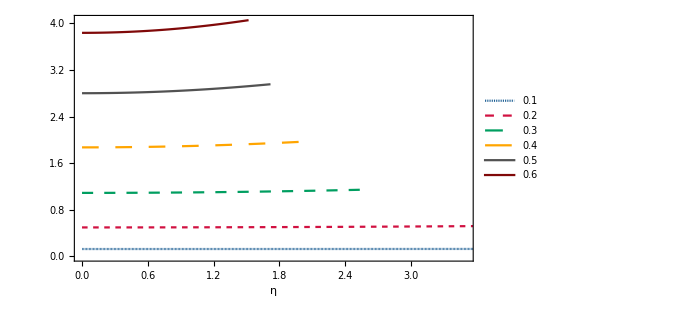

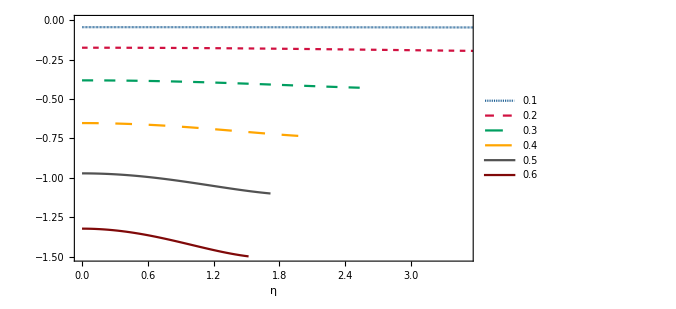

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

### Polar Modes

#### Coupled Equations

```mathematica
T1={{{0,0.24904953330653543-0.09259088336848395 ⅈ},{1/25+ⅈ/25,0.24904802144741017-0.09259068521134566 ⅈ},{2/25+(2 ⅈ)/25,0.24904348641236068-0.0925900908067607 ⅈ},{3/25+(3 ⅈ)/25,0.24903592984233075-0.09258910035707213 ⅈ},{4/25+(4 ⅈ)/25,0.2490253544658671-0.0925877141987599 ⅈ},{1/5+ⅈ/5,0.24901176409489034-0.09258593280199985 ⅈ},{6/25+(6 ⅈ)/25,0.24899516361669569-0.09258375676977225 ⅈ},{7/25+(7 ⅈ)/25,0.24897555898373266-0.09258118683672371 ⅈ},{8/25+(8 ⅈ)/25,0.24895295720121166-0.09257822386778715 ⅈ},{9/25+(9 ⅈ)/25,0.24892736631259765-0.09257486885657035 ⅈ},{2/5+(2 ⅈ)/5,0.24889879538303944-0.09257112292349953 ⅈ},{11/25+(11 ⅈ)/25,0.24886725448085373-0.09256698731377806 ⅈ},{12/25+(12 ⅈ)/25,0.24883275465709284-0.09256246339510338 ⅈ},{13/25+(13 ⅈ)/25,0.24879530792332546-0.09255755265520128 ⅈ},{14/25+(14 ⅈ)/25,0.24875492722771436-0.09255225669916946 ⅈ},{3/5+(3 ⅈ)/5,0.24871162642949649-0.09254657724664561 ⅈ},{16/25+(16 ⅈ)/25,0.2486654202719753-0.0925405161288129 ⅈ},{17/25+(17 ⅈ)/25,0.24861632435413805-0.09253407528525519 ⅈ},{18/25+(18 ⅈ)/25,0.24856435510101618-0.09252725676067636 ⅈ},{19/25+(19 ⅈ)/25,0.24850952973290744-0.09252006270149633 ⅈ},{4/5+(4 ⅈ)/5,0.24845186623358242-0.09251249535233903 ⅈ},{21/25+(21 ⅈ)/25,0.24839138331759844-0.0925045570524253 ⅈ},{22/25+(22 ⅈ)/25,0.24832810039684347-0.0924962502318858 ⅈ},{23/25+(23 ⅈ)/25,0.24826203754643378-0.09248757740800723 ⅈ},{24/25+(24 ⅈ)/25,0.24819321547008644-0.09247854118142634 ⅈ},{1+ⅈ,0.24812165546508716-0.09246914423228553 ⅈ},{26/25+(26 ⅈ)/25,0.24804737938697038-0.09245938931636269 ⅈ},{27/25+(27 ⅈ)/25,0.24797040961402697-0.0924492792611898 ⅈ},{28/25+(28 ⅈ)/25,0.24789076901174878-0.09243881696217099 ⅈ},{29/25+(29 ⅈ)/25,0.2478084808973191-0.0924280053787147 ⅈ},{6/5+(6 ⅈ)/5,0.24772356900424886-0.09241684753038923 ⅈ},{31/25+(31 ⅈ)/25,0.24763605744725758-0.09240534649311437 ⅈ},{32/25+(32 ⅈ)/25,0.24754597068749065-0.09239350539539905 ⅈ},{33/25+(33 ⅈ)/25,0.24745333349815957-0.09238132741463492 ⅈ},{34/25+(34 ⅈ)/25,0.2473581709306859-0.09236881577345511 ⅈ},{7/5+(7 ⅈ)/5,0.24726050828142507-0.09235597373616664 ⅈ},{36/25+(36 ⅈ)/25,0.24716037105903796-0.09234280460526449 ⅈ},{37/25+(37 ⅈ)/25,0.2470577849525745-0.09232931171803441 ⅈ},{38/25+(38 ⅈ)/25,0.24695277580032607-0.09231549844325086 ⅈ},{39/25+(39 ⅈ)/25,0.24684536955949832-0.09230136817797614 ⅈ},{8/5+(8 ⅈ)/5,0.24673559227674952-0.09228692434446559 ⅈ},{41/25+(41 ⅈ)/25,0.2466234700596347-0.09227217038718331 ⅈ},{42/25+(42 ⅈ)/25,0.24650902904898875-0.09225710976993239 ⅈ},{43/25+(43 ⅈ)/25,0.24639229539227794-0.09224174597310285 ⅈ},{44/25+(44 ⅈ)/25,0.24627329521794314-0.09222608249103968 ⅈ},{9/5+(9 ⅈ)/5,0.24615205461075262-0.09221012282953296 ⅈ},{46/25+(46 ⅈ)/25,0.246028599588178-0.09219387050343222 ⅈ},{47/25+(47 ⅈ)/25,0.2459029560778038-0.0921773290343846 ⅈ},{48/25+(48 ⅈ)/25,0.24577514989577232-0.09216050194869913 ⅈ},{49/25+(49 ⅈ)/25,0.24564520672626838-0.0921433927753351 ⅈ},{2+2 ⅈ,0.24551315210203767-0.09212600504401602 ⅈ},{51/25+(51 ⅈ)/25,0.2453790113859339-0.09210834228346694 ⅈ},{52/25+(52 ⅈ)/25,0.24524280975348467-0.09209040801977465 ⅈ},{53/25+(53 ⅈ)/25,0.24510457217646364-0.09207220577486919 ⅈ},{54/25+(54 ⅈ)/25,0.24496432340745325-0.09205373906512453 ⅈ},{11/5+(11 ⅈ)/5,0.24482208796538119-0.09203501140007705 ⅈ},{56/25+(56 ⅈ)/25,0.24467789012200988-0.09201602628125859 ⅈ},{57/25+(57 ⅈ)/25,0.24453175388935822-0.09199678720114235 ⅈ},{58/25+(58 ⅈ)/25,0.24438370300803197-0.09197729764219861 ⅈ},{59/25+(59 ⅈ)/25,0.24423376093643764-0.09195756107605728 ⅈ},{12/5+(12 ⅈ)/5,0.24408195084085496-0.09193758096277463 ⅈ},{61/25+(61 ⅈ)/25,0.24392829558634002-0.09191736075020102 ⅈ},{62/25+(62 ⅈ)/25,0.24377281772843215-0.09189690387344614 ⅈ},{63/25+(63 ⅈ)/25,0.24361553950563586-0.09187621375443891 ⅈ},{64/25+(64 ⅈ)/25,0.24345648283264867-0.0918552938015788 ⅈ},{13/5+(13 ⅈ)/5,0.24329566929430713-0.09183414740947454 ⅈ},{66/25+(66 ⅈ)/25,0.2431331201402198-0.09181277795876805 ⅈ},{67/25+(67 ⅈ)/25,0.24296885628005976-0.09179118881603937 ⅈ},{68/25+(68 ⅈ)/25,0.24280289827948645-0.0917693833337893 ⅈ},{69/25+(69 ⅈ)/25,0.24263526635666782-0.09174736485049735 ⅈ},{14/5+(14 ⅈ)/5,0.24246598037937486-0.09172513669075057 ⅈ},{71/25+(71 ⅈ)/25,0.2422950598626197-0.0917027021654412 ⅈ},{72/25+(72 ⅈ)/25,0.24212252396680953-0.09168006457202899 ⅈ},{73/25+(73 ⅈ)/25,0.24194839149638875-0.09165722719486605 ⅈ},{74/25+(74 ⅈ)/25,0.24177268089894394-0.0916341933055806 ⅈ},{3+3 ⅈ,0.24159541026474338-0.09161096616351724 ⅈ},{76/25+(76 ⅈ)/25,0.24141659732668844-0.09158754901623024 ⅈ},{77/25+(77 ⅈ)/25,0.24123625946064967-0.09156394510002792 ⅈ},{78/25+(78 ⅈ)/25,0.2410544136861658-0.09154015764056496 ⅈ},{79/25+(79 ⅈ)/25,0.24087107666748095-0.09151618985348026 ⅈ},{16/5+(16 ⅈ)/5,0.24068626471489893-0.09149204494507777 ⅈ},{81/25+(81 ⅈ)/25,0.24049999378643253-0.09146772611304844 ⅈ},{82/25+(82 ⅈ)/25,0.24031227948972678-0.09144323654723019 ⅈ},{83/25+(83 ⅈ)/25,0.2401231370842376-0.09141857943040466 ⅈ},{84/25+(84 ⅈ)/25,0.23993258148364538-0.09139375793912796 ⅈ},{17/5+(17 ⅈ)/5,0.2397406272584857-0.09136877524459404 ⅈ},{86/25+(86 ⅈ)/25,0.23954728863898042-0.09134363451352835 ⅈ},{87/25+(87 ⅈ)/25,0.23935257951805186-0.09131833890911041 ⅈ},{88/25+(88 ⅈ)/25,0.23915651345450367-0.09129289159192333 ⅈ},{89/25+(89 ⅈ)/25,0.23895910367635495-0.09126729572092905 ⅈ},{18/5+(18 ⅈ)/5,0.2387603630843117-0.09124155445446727 ⅈ},{91/25+(91 ⅈ)/25,0.23856030425536287-0.09121567095127753 ⅈ},{92/25+(92 ⅈ)/25,0.23835893944648767-0.09118964837154189 ⅈ},{93/25+(93 ⅈ)/25,0.23815628059846236-0.0911634898779487 ⅈ},{94/25+(94 ⅈ)/25,0.2379523393397549-0.09113719863677444 ⅈ},{19/5+(19 ⅈ)/5,0.23774712699049622-0.09111077781898393 ⅈ},{96/25+(96 ⅈ)/25,0.2375406545665186-0.09108423060134747 ⅈ},{97/25+(97 ⅈ)/25,0.23733293278345086-0.09105756016757378 ⅈ},{98/25+(98 ⅈ)/25,0.23712397206086175-0.0910307697094585 ⅈ},{99/25+(99 ⅈ)/25,0.23691378252644327-0.09100386242804663 ⅈ},{4+4 ⅈ,0.23670237402022515-0.09097684153480899 ⅈ},{101/25+(101 ⅈ)/25,0.23648975609881412-0.09094971025283181 ⅈ},{102/25+(102 ⅈ)/25,0.23627593803965058-0.09092247181801831 ⅈ},{103/25+(103 ⅈ)/25,0.23606092884527624-0.0908951294803031 ⅈ},{104/25+(104 ⅈ)/25,0.23584473724760677-0.09086768650487716 ⅈ},{21/5+(21 ⅈ)/5,0.23562737171220424-0.09084014617342458 ⅈ},{106/25+(106 ⅈ)/25,0.23540884044254395-0.09081251178536967 ⅈ},{107/25+(107 ⅈ)/25,0.23518915138427093-0.09078478665913471 ⅈ},{108/25+(108 ⅈ)/25,0.23496831222944203-0.09075697413340769 ⅈ},{109/25+(109 ⅈ)/25,0.23474633042074938-0.09072907756841997 ⅈ},{22/5+(22 ⅈ)/5,0.2345232131557218-0.09070110034723408 ⅈ},{111/25+(111 ⅈ)/25,0.23429896739090045-0.09067304587704039 ⅈ},{112/25+(112 ⅈ)/25,0.23407359984598644-0.09064491759046428 ⅈ},{113/25+(113 ⅈ)/25,0.23384711700795696-0.09061671894688192 ⅈ},{114/25+(114 ⅈ)/25,0.2336195251351476-0.09058845343374594 ⅈ},{23/5+(23 ⅈ)/5,0.23339083026129945-0.09056012456792051 ⅈ},{116/25+(116 ⅈ)/25,0.23316103819956782-0.09053173589702583 ⅈ},{117/25+(117 ⅈ)/25,0.23293015454649182-0.09050329100079207 ⅈ},{118/25+(118 ⅈ)/25,0.23269818468592304-0.09047479349242353 ⅈ},{119/25+(119 ⅈ)/25,0.23246513379291175-0.0904462470199717 ⅈ},{24/5+(24 ⅈ)/5,0.2322310068375501-0.090417655267719 ⅈ},{121/25+(121 ⅈ)/25,0.2319958085887708-0.09038902195757238 ⅈ},{122/25+(122 ⅈ)/25,0.2317595436181011-0.09036035085046719 ⅈ},{123/25+(123 ⅈ)/25,0.23152221630337108-0.0903316457477816 ⅈ},{124/25+(124 ⅈ)/25,0.23128383083237597-0.09030291049276207 ⅈ},{5+5 ⅈ,0.23104439120649245-0.09027414897195941 ⅈ},{126/25+(126 ⅈ)/25,0.23080390124424843-0.0902453651166765 ⅈ},{127/25+(127 ⅈ)/25,0.2305623645848465-0.09021656290442762 ⅈ},{128/25+(128 ⅈ)/25,0.23031978469164088-0.09018774636040969 ⅈ},{129/25+(129 ⅈ)/25,0.2300761648555688-0.09015891955898565 ⅈ},{26/5+(26 ⅈ)/5,0.22983150819853565-0.09013008662518074 ⅈ},{131/25+(131 ⅈ)/25,0.2295858176767551-0.09010125173619164 ⅈ},{132/25+(132 ⅈ)/25,0.229339096084044-0.09007241912290899 ⅈ},{133/25+(133 ⅈ)/25,0.22909134605507395-0.09004359307145351 ⅈ},{134/25+(134 ⅈ)/25,0.22884257006857794-0.09001477792472679 ⅈ},{27/5+(27 ⅈ)/5,0.22859277045051565-0.08998597808397611 ⅈ},{136/25+(136 ⅈ)/25,0.2283419493771957-0.08995719801037459 ⅈ},{137/25+(137 ⅈ)/25,0.22809010887835734-0.08992844222661668 ⅈ},{138/25+(138 ⅈ)/25,0.22783725084021214-0.08989971531852961 ⅈ},{139/25+(139 ⅈ)/25,0.2275833770084459-0.08987102193670114 ⅈ},{28/5+(28 ⅈ)/5,0.22732848899118352-0.08984236679812407 ⅈ},{141/25+(141 ⅈ)/25,0.22707258826191629-0.08981375468785832 ⅈ},{142/25+(142 ⅈ)/25,0.2268156761623936-0.0897851904607103 ⅈ},{143/25+(143 ⅈ)/25,0.22655775390548044-0.08975667904293104 ⅈ},{144/25+(144 ⅈ)/25,0.22629882257798137-0.08972822543393265 ⅈ},{29/5+(29 ⅈ)/5,0.22603888314343315-0.08969983470802448 ⅈ},{146/25+(146 ⅈ)/25,0.22577793644486607-0.08967151201616852 ⅈ},{147/25+(147 ⅈ)/25,0.22551598320753724-0.0896432625877556 ⅈ},{148/25+(148 ⅈ)/25,0.22525302404163533-0.08961509173240186 ⅈ},{149/25+(149 ⅈ)/25,0.22498905944495964-0.08958700484176707 ⅈ},{6+6 ⅈ,0.2247240898055747-0.08955900739139427 ⅈ},{151/25+(151 ⅈ)/25,0.22445811540444144-0.08953110494257227 ⅈ},{152/25+(152 ⅈ)/25,0.22419113641802724-0.08950330314422046 ⅈ},{153/25+(153 ⅈ)/25,0.22392315292089607-0.08947560773479776 ⅈ},{154/25+(154 ⅈ)/25,0.2236541648882804-0.08944802454423487 ⅈ},{31/5+(31 ⅈ)/5,0.22338417219863732-0.08942055949589138 ⅈ},{156/25+(156 ⅈ)/25,0.22311317463618907-0.08939321860853787 ⅈ},{157/25+(157 ⅈ)/25,0.22284117189345162-0.0893660079983635 ⅈ},{158/25+(158 ⅈ)/25,0.22256816357375145-0.08933893388100979 ⅈ},{159/25+(159 ⅈ)/25,0.22229414919373394-0.08931200257363094 ⅈ},{32/5+(32 ⅈ)/5,0.22201912818586372-0.08928522049698126 ⅈ},{161/25+(161 ⅈ)/25,0.22174309990092023-0.08925859417753067 ⅈ},{162/25+(162 ⅈ)/25,0.2214660636104897-0.08923213024960785 ⅈ},{163/25+(163 ⅈ)/25,0.2211880185094558-0.08920583545757263 ⅈ},{164/25+(164 ⅈ)/25,0.22090896371849092-0.08917971665801719 ⅈ},{33/5+(33 ⅈ)/5,0.2206288982865506-0.08915378082199746 ⅈ},{166/25+(166 ⅈ)/25,0.22034782119337215-0.08912803503729423 ⅈ},{167/25+(167 ⅈ)/25,0.2200657313519814-0.08910248651070567 ⅈ},{168/25+(168 ⅈ)/25,0.21978262761120795-0.0890771425703703 ⅈ},{169/25+(169 ⅈ)/25,0.2194985087582125-0.08905201066812232 ⅈ},{34/5+(34 ⅈ)/5,0.21921337352102793-0.08902709838187843 ⅈ},{171/25+(171 ⅈ)/25,0.21892722057111694-0.08900241341805791 ⅈ},{172/25+(172 ⅈ)/25,0.21864004852594823-0.08897796361403508 ⅈ},{173/25+(173 ⅈ)/25,0.21835185595159387-0.0889537569406254 ⅈ},{174/25+(174 ⅈ)/25,0.21806264136535083-0.08892980150460553 ⅈ},{7+7 ⅈ,0.21777240323838853-0.08890610555126699 ⅈ},{176/25+(176 ⅈ)/25,0.2174811399984254-0.08888267746700489 ⅈ},{177/25+(177 ⅈ)/25,0.2171888500324376-0.08885952578194112 ⅈ},{178/25+(178 ⅈ)/25,0.2168955316894018-0.08883665917258268 ⅈ}},{{0,0.2513922213744943-0.09289841463615552 ⅈ},{1/25+ⅈ/25,0.2513861772520305-0.09289762475851178 ⅈ},{2/25+(2 ⅈ)/25,0.2513680538446794-0.09289525620959002 ⅈ},{3/25+(3 ⅈ)/25,0.25133787801589286-0.09289131224081079 ⅈ},{4/25+(4 ⅈ)/25,0.2512956942724765-0.0928857982417839 ⅈ},{1/5+ⅈ/5,0.25124156439244777-0.09287872169949693 ⅈ},{6/25+(6 ⅈ)/25,0.2511755669056639-0.09287009214122863 ⅈ},{7/25+(7 ⅈ)/25,0.2510977964429324-0.09285992106306223 ⅈ},{8/25+(8 ⅈ)/25,0.2510083629654824-0.09284822184534625 ⅈ},{9/25+(9 ⅈ)/25,0.25090739088849184-0.09283500965665373 ⅈ},{2/5+(2 ⅈ)/5,0.2507950181137667-0.09282030134794862 ⅈ},{11/25+(11 ⅈ)/25,0.25067139498761654-0.09280411533877538 ⅈ},{12/25+(12 ⅈ)/25,0.2505366832004691-0.09278647149734214 ⅈ},{13/25+(13 ⅈ)/25,0.2503910546448329-0.09276739101637446 ⅈ},{14/25+(14 ⅈ)/25,0.25023469024787026-0.09274689628657631 ⅈ},{3/5+(3 ⅈ)/5,0.2500677787941469-0.0927250107694542 ⅈ},{16/25+(16 ⅈ)/25,0.24989051575311233-0.0927017588711447 ⅈ},{17/25+(17 ⅈ)/25,0.24970310212461488-0.09267716581874226 ⅈ},{18/25+(18 ⅈ)/25,0.24950574331431652-0.09265125754046168 ⅈ},{19/25+(19 ⅈ)/25,0.24929864804931812-0.09262406055079025 ⅈ},{4/5+(4 ⅈ)/5,0.24908202734268603-0.09259560184160287 ⅈ},{21/25+(21 ⅈ)/25,0.24885609351394264-0.09256590878002775 ⅈ},{22/25+(22 ⅈ)/25,0.24862105927099626-0.09253500901367005 ⅈ},{23/25+(23 ⅈ)/25,0.24837713685746957-0.09250293038363042 ⅈ},{24/25+(24 ⅈ)/25,0.24812453726797978-0.09246970084559618 ⅈ},{1+ⅈ,0.24786346953264352-0.09243534839913839 ⅈ},{26/25+(26 ⅈ)/25,0.24759414007094235-0.09239990102522094 ⅈ},{27/25+(27 ⅈ)/25,0.24731675211409712-0.09236338663181717 ⅈ},{28/25+(28 ⅈ)/25,0.24703150519426323-0.09232583300743495 ⅈ},{29/25+(29 ⅈ)/25,0.24673859469817036-0.09228726778227686 ⅈ},{6/5+(6 ⅈ)/5,0.24643821148228384-0.09224771839669982 ⅈ},{31/25+(31 ⅈ)/25,0.24613054154614605-0.0922072120765939 ⅈ},{32/25+(32 ⅈ)/25,0.24581576576026043-0.0921657758152677 ⅈ},{33/25+(33 ⅈ)/25,0.2454940596446867-0.09212343636140789 ⅈ},{34/25+(34 ⅈ)/25,0.2451655931944166-0.09208022021266997 ⅈ},{7/5+(7 ⅈ)/5,0.24483053074757696-0.09203615361445827 ⅈ},{36/25+(36 ⅈ)/25,0.24448903089255125-0.09199126256345731 ⅈ},{37/25+(37 ⅈ)/25,0.24414124641020787-0.09194557281549115 ⅈ},{38/25+(38 ⅈ)/25,0.24378732424756172-0.0918991098973041 ⅈ},{39/25+(39 ⅈ)/25,0.2434274055193686-0.09185189912187641 ⅈ},{8/5+(8 ⅈ)/5,0.24306162553434524-0.09180396560691251 ⅈ},{41/25+(41 ⅈ)/25,0.24269011384291808-0.09175533429616427 ⅈ},{42/25+(42 ⅈ)/25,0.24231299430362352-0.09170602998327815 ⅈ},{43/25+(43 ⅈ)/25,0.24193038516550483-0.09165607733788081 ⅈ},{44/25+(44 ⅈ)/25,0.2415423991640731-0.09160550093364422 ⅈ},{9/5+(9 ⅈ)/5,0.24114914362861659-0.09155432527809805 ⅈ},{46/25+(46 ⅈ)/25,0.24075072059885452-0.09150257484398011 ⅈ},{47/25+(47 ⅈ)/25,0.24034722694913102-0.09145027410194126 ⅈ},{48/25+(48 ⅈ)/25,0.2399387545185379-0.09139744755444211 ⅈ},{49/25+(49 ⅈ)/25,0.2395253902455321-0.0913441197707019 ⅈ},{2+2 ⅈ,0.23910721630578122-0.09129031542257776 ⅈ},{51/25+(51 ⅈ)/25,0.23868431025212714-0.09123605932127257 ⅈ},{52/25+(52 ⅈ)/25,0.23825674515569698-0.09118137645478575 ⅈ},{53/25+(53 ⅈ)/25,0.23782458974732337-0.09112629202603748 ⅈ},{54/25+(54 ⅈ)/25,0.23738790855855507-0.09107083149161055 ⅈ},{11/5+(11 ⅈ)/5,0.2369467620616442-0.09101502060106809 ⅈ},{56/25+(56 ⅈ)/25,0.23650120680799658-0.09095888543681559 ⅈ},{57/25+(57 ⅈ)/25,0.23605129556465754-0.09090245245448862 ⅈ},{58/25+(58 ⅈ)/25,0.23559707744848396-0.09084574852385581 ⅈ},{59/25+(59 ⅈ)/25,0.23513859805772375-0.09078880097023496 ⅈ},{12/5+(12 ⅈ)/5,0.23467589960078636-0.09073163761643022 ⅈ},{61/25+(61 ⅈ)/25,0.23420902102204244-0.0906742868252037 ⅈ},{62/25+(62 ⅈ)/25,0.23373799812454057-0.09061677754230046 ⅈ},{63/25+(63 ⅈ)/25,0.23326286368957094-0.0905591393400547 ⅈ},{64/25+(64 ⅈ)/25,0.2327836475930458-0.09050140246160604 ⅈ},{13/5+(13 ⅈ)/5,0.23230037691869693-0.09044359786576295 ⅈ},{66/25+(66 ⅈ)/25,0.2318130760681228-0.0903857572725519 ⅈ},{67/25+(67 ⅈ)/25,0.23132176686774167-0.09032791320949603 ⅈ},{68/25+(68 ⅈ)/25,0.2308264686727298-0.09027009905866965 ⅈ},{69/25+(69 ⅈ)/25,0.23032719846804448-0.09021234910457789 ⅈ},{14/5+(14 ⅈ)/5,0.22982397096664756-0.09015469858291378 ⅈ},{71/25+(71 ⅈ)/25,0.22931679870506183-0.09009718373024671 ⅈ},{72/25+(72 ⅈ)/25,0.22880569213640514-0.09003984183469861 ⅈ},{73/25+(73 ⅈ)/25,0.22829065972105958-0.08998271128766616 ⅈ},{74/25+(74 ⅈ)/25,0.22777170801514365-0.08992583163664804 ⅈ},{3+3 ⅈ,0.22724884175696589-0.08986924363923826 ⅈ},{76/25+(76 ⅈ)/25,0.22672206395164662-0.0898129893183474 ⅈ},{77/25+(77 ⅈ)/25,0.2261913759541038-0.08975711201871393 ⅈ},{78/25+(78 ⅈ)/25,0.2256567775506061-0.089701656464769 ⅈ},{79/25+(79 ⅈ)/25,0.22511826703910615-0.08964666881991781 ⅈ},{16/5+(16 ⅈ)/5,0.22457584130857217-0.08959219674730075 ⅈ},{81/25+(81 ⅈ)/25,0.22402949591754645-0.08953828947209683 ⅈ},{82/25+(82 ⅈ)/25,0.22347922517216562-0.08948499784543283 ⅈ},{83/25+(83 ⅈ)/25,0.22292502220388702-0.08943237440995755 ⅈ},{84/25+(84 ⅈ)/25,0.22236687904717353-0.08938047346714183 ⅈ},{17/5+(17 ⅈ)/5,0.2218047867173993-0.08932935114636205 ⅈ},{86/25+(86 ⅈ)/25,0.22123873528924812-0.08927906547582128 ⅈ},{87/25+(87 ⅈ)/25,0.22066871397588647-0.08922967645536116 ⅈ},{88/25+(88 ⅈ)/25,0.2200947112092064-0.08918124613121173 ⅈ},{89/25+(89 ⅈ)/25,0.21951671472144296-0.08913383867272358 ⅈ},{18/5+(18 ⅈ)/5,0.21893471162848674-0.08908752045111935 ⅈ},{91/25+(91 ⅈ)/25,0.2183486885152241-0.08904236012029738 ⅈ}},{{0,0.2552443161152394-0.09340456216904312 ⅈ},{1/25+ⅈ/25,0.25523071954783044-0.09340279449208581 ⅈ},{2/25+(2 ⅈ)/25,0.2551899772951585-0.09339749703267484 ⅈ},{3/25+(3 ⅈ)/25,0.25512223089622954-0.09338868642088136 ⅈ},{4/25+(4 ⅈ)/25,0.25502771311651923-0.09337639003518598 ⅈ},{1/5+ⅈ/5,0.2549067434400436-0.0933606455171281 ⅈ},{6/25+(6 ⅈ)/25,0.25475972201522784-0.09334150011988661 ⅈ},{7/25+(7 ⅈ)/25,0.2545871223187073-0.09331900992027731 ⅈ},{8/25+(8 ⅈ)/25,0.2543894828261668-0.0932932389261344 ⅈ},{9/25+(9 ⅈ)/25,0.25416739799846794-0.09326425811313746 ⅈ},{2/5+(2 ⅈ)/5,0.2539215088915216-0.09323214442514009 ⅈ},{11/25+(11 ⅈ)/25,0.25365249368180365-0.09319697977019102 ⅈ},{12/25+(12 ⅈ)/25,0.25336105836940803-0.09315885004109008 ⅈ},{13/25+(13 ⅈ)/25,0.2530479278810876-0.09311784418493017 ⅈ},{14/25+(14 ⅈ)/25,0.2527138377509415-0.09307405334110118 ⅈ},{3/5+(3 ⅈ)/5,0.2523595265100649-0.09302757006209497 ⅈ},{16/25+(16 ⅈ)/25,0.2519857288717583-0.09297848762650143 ⅈ},{17/25+(17 ⅈ)/25,0.25159316975816765-0.0929268994490884 ⅈ},{18/25+(18 ⅈ)/25,0.2511825591790835-0.09287289858898748 ⅈ},{19/25+(19 ⅈ)/25,0.2507545879448479-0.09281657735384942 ⅈ},{4/5+(4 ⅈ)/5,0.25030992417308984-0.09275802699540271 ⅈ},{21/25+(21 ⅈ)/25,0.24984921053301426-0.09269733749011577 ⅈ},{22/25+(22 ⅈ)/25,0.24937306216056826-0.09263459739754781 ⅈ},{23/25+(23 ⅈ)/25,0.248882065172182-0.09256989378839077 ⅈ},{24/25+(24 ⅈ)/25,0.2483767757030328-0.09250331223404881 ⅈ},{1+ⅈ,0.2478577193970316-0.09243493684977723 ⅈ},{26/25+(26 ⅈ)/25,0.2473253912791739-0.09236485038381953 ⅈ},{27/25+(27 ⅈ)/25,0.2467802559458264-0.09229313434555995 ⅈ},{28/25+(28 ⅈ)/25,0.246222748014357-0.09221986916638718 ⅈ},{29/25+(29 ⅈ)/25,0.24565327277978624-0.09214513438768597 ⅈ},{6/5+(6 ⅈ)/5,0.24507220703249588-0.09206900887110649 ⅈ},{31/25+(31 ⅈ)/25,0.2444798999972142-0.09199157102696942 ⅈ},{32/25+(32 ⅈ)/25,0.24387667435933014-0.09191289905733485 ⅈ},{33/25+(33 ⅈ)/25,0.24326282734996452-0.09183307121087958 ⅈ},{34/25+(34 ⅈ)/25,0.24263863186608361-0.09175216604728775 ⅈ},{7/5+(7 ⅈ)/5,0.24200433760625956-0.09167026270935646 ⅈ},{36/25+(36 ⅈ)/25,0.24136017220646871-0.09158744120145841 ⅈ},{37/25+(37 ⅈ)/25,0.2407063423636029-0.09150378267338558 ⅈ},{38/25+(38 ⅈ)/25,0.2400430349371775-0.09141936970892785 ⅈ},{39/25+(39 ⅈ)/25,0.23937041802211056-0.09133428661882445 ⅈ},{8/5+(8 ⅈ)/5,0.23868864198745357-0.09124861973796569 ⅈ},{41/25+(41 ⅈ)/25,0.2379978404776276-0.09116245772692672 ⅈ},{42/25+(42 ⅈ)/25,0.23729813137410813-0.09107589187808687 ⅈ},{43/25+(43 ⅈ)/25,0.23658961771663609-0.09098901642673067 ⅈ},{44/25+(44 ⅈ)/25,0.23587238858396428-0.09090192886764871 ⅈ},{9/5+(9 ⅈ)/5,0.2351465199349005-0.09081473027785401 ⅈ},{46/25+(46 ⅈ)/25,0.2344120754110167-0.09072752564611437 ⅈ},{47/25+(47 ⅈ)/25,0.2336691071028814-0.09064042421006871 ⅈ},{48/25+(48 ⅈ)/25,0.23291765628206643-0.09055353980175063 ⅈ},{49/25+(49 ⅈ)/25,0.2321577541014946-0.09046699120238891 ⅈ},{2+2 ⅈ,0.23138942226695333-0.09038090250738859 ⅈ},{51/25+(51 ⅈ)/25,0.230612673682812-0.09029540350242346 ⅈ},{52/25+(52 ⅈ)/25,0.22982751307516341-0.09021063005158965 ⅈ},{53/25+(53 ⅈ)/25,0.22903393759577068-0.09012672449857863 ⅈ},{54/25+(54 ⅈ)/25,0.22823193741035083-0.09004383608182945 ⅈ},{11/5+(11 ⅈ)/5,0.22742149627487324-0.08996212136461179 ⅈ},{56/25+(56 ⅈ)/25,0.22660259210369973-0.08988174468097113 ⅈ},{57/25+(57 ⅈ)/25,0.22577519753355568-0.08980287859843546 ⅈ},{58/25+(58 ⅈ)/25,0.22493928048749415-0.08972570439833646 ⅈ},{59/25+(59 ⅈ)/25,0.22409480474321117-0.08965041257453299 ⅈ},{12/5+(12 ⅈ)/5,0.2232417305102888-0.08957720335123921 ⅈ},{61/25+(61 ⅈ)/25,0.22238001502119137-0.08950628722054928 ⅈ},{62/25+(62 ⅈ)/25,0.22150961314111547-0.08943788550010931 ⅈ},{63/25+(63 ⅈ)/25,0.22063047800211308-0.08937223091120992 ⅈ},{64/25+(64 ⅈ)/25,0.2197425616672511-0.08930956817735317 ⅈ}},{{0,0.2605316834521421-0.09410018395896062 ⅈ},{1/25+ⅈ/25,0.260507482443302-0.09409706237703763 ⅈ},{2/25+(2 ⅈ)/25,0.26043503927076683-0.09408771567951954 ⅈ},{3/25+(3 ⅈ)/25,0.26031482782666604-0.09407219742125486 ⅈ},{4/25+(4 ⅈ)/25,0.2601476186702098-0.09405059483673647 ⅈ},{1/5+ⅈ/5,0.259934451851668-0.094023025990767 ⅈ},{6/25+(6 ⅈ)/25,0.2596766018559289-0.09398963610963403 ⅈ},{7/25+(7 ⅈ)/25,0.25937553721180917-0.09395059336648563 ⅈ},{8/25+(8 ⅈ)/25,0.25903287741116193-0.0939060844043474 ⅈ},{9/25+(9 ⅈ)/25,0.2586503496248578-0.09385630986309514 ⅈ},{2/5+(2 ⅈ)/5,0.2582297473332843-0.09380148013676275 ⅈ},{11/25+(11 ⅈ)/25,0.25777289249301005-0.09374181153409519 ⅈ},{12/25+(12 ⅈ)/25,0.2572816023238151-0.09367752295742753 ⅈ},{13/25+(13 ⅈ)/25,0.2567576612910781-0.09360883316027836 ⅈ},{14/25+(14 ⅈ)/25,0.2562027984245006-0.09353595859754225 ⅈ},{3/5+(3 ⅈ)/5,0.25561866977900044-0.09345911184636842 ⅈ},{16/25+(16 ⅈ)/25,0.2550068456115255-0.09337850055115726 ⅈ},{17/25+(17 ⅈ)/25,0.2543688017092988-0.09329432683157551 ⅈ},{18/25+(18 ⅈ)/25,0.25370591424388644-0.09320678708626143 ⅈ},{19/25+(19 ⅈ)/25,0.25301945752223903-0.09311607212488422 ⅈ},{4/5+(4 ⅈ)/5,0.25231060404207795-0.09302236756543829 ⅈ},{21/25+(21 ⅈ)/25,0.2515804263189709-0.09292585444040095 ⅈ},{22/25+(22 ⅈ)/25,0.25082990002393846-0.0928267099633445 ⅈ},{23/25+(23 ⅈ)/25,0.2500599080446546-0.09272510841581953 ⅈ},{24/25+(24 ⅈ)/25,0.249271245154452-0.09262122212220192 ⅈ},{1+ⅈ,0.24846462303800165-0.09251522248735088 ⅈ},{26/25+(26 ⅈ)/25,0.2476406754790426-0.09240728107818905 ⅈ},{27/25+(27 ⅈ)/25,0.2467999635634388-0.09229757073563757 ⅈ},{28/25+(28 ⅈ)/25,0.245942980790445-0.09218626670776707 ⅈ},{29/25+(29 ⅈ)/25,0.24507015801712126-0.09207354779862195 ⅈ},{6/5+(6 ⅈ)/5,0.24418186818630003-0.09195959753007399 ⅈ},{31/25+(31 ⅈ)/25,0.24327843080838532-0.09184460531633983 ⅈ},{32/25+(32 ⅈ)/25,0.24236011618252737-0.0917287676525857 ⅈ},{33/25+(33 ⅈ)/25,0.2414271493542445-0.09161228932042066 ⅈ},{34/25+(34 ⅈ)/25,0.24047971381513047-0.0914953846141333 ⅈ},{7/5+(7 ⅈ)/5,0.23951795495654665-0.09137827859232434 ⅈ},{36/25+(36 ⅈ)/25,0.23854198329369813-0.0912612083601793 ⅈ},{37/25+(37 ⅈ)/25,0.23755187747967973-0.09114442438805914 ⅈ},{38/25+(38 ⅈ)/25,0.23654768713131322-0.09102819187238674 ⅈ},{39/25+(39 ⅈ)/25,0.2355294354901714-0.09091279214500218 ⅈ},{8/5+(8 ⅈ)/5,0.23449712194332736-0.09079852413725358 ⅈ},{41/25+(41 ⅈ)/25,0.23345072442926787-0.0906857059050936 ⅈ},{42/25+(42 ⅈ)/25,0.23239020175520766-0.09057467622135465 ⅈ},{43/25+(43 ⅈ)/25,0.23131549585286035-0.09046579624116866 ⅈ},{44/25+(44 ⅈ)/25,0.23022653400065157-0.0903594512461556 ⅈ},{9/5+(9 ⅈ)/5,0.22912323104148338-0.09025605247250046 ⅈ},{46/25+(46 ⅈ)/25,0.22800549162653164-0.09015603902732723 ⅈ},{47/25+(47 ⅈ)/25,0.22687321251724687-0.09005987989680654 ⅈ},{48/25+(48 ⅈ)/25,0.22572628497975952-0.08996807604813549 ⅈ},{49/25+(49 ⅈ)/25,0.2245645973083223-0.08988116262581287 ⅈ},{2+2 ⅈ,0.22338803751725528-0.08979971124040159 ⅈ}},{{0,0.2671585575236661-0.09497327544666492 ⅈ},{1/25+ⅈ/25,0.267120587666371-0.094968432608322 ⅈ},{2/25+(2 ⅈ)/25,0.26700710320574267-0.09495394994265642 ⅈ},{3/25+(3 ⅈ)/25,0.2668193538332243-0.09492996239371523 ⅈ},{4/25+(4 ⅈ)/25,0.2665593390842937-0.09489668638397337 ⅈ},{1/5+ⅈ/5,0.26622969504065264-0.0948544082978734 ⅈ},{6/25+(6 ⅈ)/25,0.2658335559600921-0.09480347045808939 ⅈ},{7/25+(7 ⅈ)/25,0.26537440583483496-0.0947442561501306 ⅈ},{8/25+(8 ⅈ)/25,0.26485593345447483-0.09467717510035226 ⅈ},{9/25+(9 ⅈ)/25,0.26428190139649604-0.09460265048349674 ⅈ},{2/5+(2 ⅈ)/5,0.2636560354876403-0.0945211081320805 ⅈ},{11/25+(11 ⅈ)/25,0.26298193757233995-0.09443296823487042 ⅈ},{12/25+(12 ⅈ)/25,0.26226302145864644-0.09433863950441922 ⅈ},{13/25+(13 ⅈ)/25,0.26150246990544-0.09423851558661761 ⅈ},{14/25+(14 ⅈ)/25,0.26070320942158265-0.0941329733735056 ⅈ},{3/5+(3 ⅈ)/5,0.2598678992786032-0.09402237284424184 ⅈ},{16/25+(16 ⅈ)/25,0.2589989312616696-0.09390705807389463 ⅈ},{17/25+(17 ⅈ)/25,0.2580984370886854-0.09378735909362262 ⅈ},{18/25+(18 ⅈ)/25,0.25716830095383303-0.09366359434212013 ⅈ},{19/25+(19 ⅈ)/25,0.25621017519312506-0.09353607350582255 ⅈ},{4/5+(4 ⅈ)/5,0.25522549756433105-0.09340510059796223 ⅈ},{21/25+(21 ⅈ)/25,0.2542155090538037-0.09327097717123799 ⅈ},{22/25+(22 ⅈ)/25,0.2531812714612119-0.09313400559491666 ⅈ},{23/25+(23 ⅈ)/25,0.2521236842749461-0.092994492355176 ⅈ},{24/25+(24 ⅈ)/25,0.2510435005465604-0.09285275135854733 ⅈ},{1+ⅈ,0.2499413416143317-0.09270910723372139 ⅈ},{26/25+(26 ⅈ)/25,0.24881771062564853-0.09256389863797651 ⅈ},{27/25+(27 ⅈ)/25,0.24767300487578175-0.09241748158214802 ⅈ},{28/25+(28 ⅈ)/25,0.2465075270251391-0.09227023279325211 ⅈ},{29/25+(29 ⅈ)/25,0.24532149528505434-0.09212255313728548 ⅈ},{6/5+(6 ⅈ)/5,0.24411505267867137-0.09197487112684571 ⅈ},{31/25+(31 ⅈ)/25,0.24288827549241546-0.0918276465394101 ⅈ},{32/25+(32 ⅈ)/25,0.24164118103775015-0.09168137417260849 ⅈ},{33/25+(33 ⅈ)/25,0.2403737348444866-0.09153658776275007 ⅈ},{34/25+(34 ⅈ)/25,0.23908585740734042-0.09139386409226531 ⅈ},{7/5+(7 ⅈ)/5,0.23777743060781278-0.0912538273105519 ⅈ},{36/25+(36 ⅈ)/25,0.2364483039345881-0.0911171534908642 ⅈ},{37/25+(37 ⅈ)/25,0.23509830062807216-0.09098457544315143 ⅈ},{38/25+(38 ⅈ)/25,0.23372722387886172-0.09085688779885488 ⅈ},{39/25+(39 ⅈ)/25,0.2323348632161638-0.09073495237822576 ⅈ},{8/5+(8 ⅈ)/5,0.2309210012307036-0.0906197038432131 ⅈ},{41/25+(41 ⅈ)/25,0.2294854207876226-0.09051215562873197 ⅈ},{42/25+(42 ⅈ)/25,0.22802791289833935-0.09041340613131509 ⅈ},{43/25+(43 ⅈ)/25,0.22654828543624794-0.09032464511570874 ⅈ}},{{0,0.27501383123134077-0.0960095165980962 ⅈ},{1/25+ⅈ/25,0.2749586629602288-0.0960025870620997 ⅈ},{2/25+(2 ⅈ)/25,0.27479414272845365-0.09598189957919588 ⅈ},{3/25+(3 ⅈ)/25,0.27452313140441864-0.09594774836405019 ⅈ},{4/25+(4 ⅈ)/25,0.274150105003455-0.0959005949467649 ⅈ},{1/5+ⅈ/5,0.27368077779417577-0.09584103108472636 ⅈ},{6/25+(6 ⅈ)/25,0.2731216754482736-0.09576973694671566 ⅈ},{7/25+(7 ⅈ)/25,0.27247972039720464-0.0956874407891112 ⅈ},{8/25+(8 ⅈ)/25,0.2717618742647394-0.09559488459453562 ⅈ},{9/25+(9 ⅈ)/25,0.27097486056487574-0.09549279796088993 ⅈ},{2/5+(2 ⅈ)/5,0.27012497188304924-0.09538188062585738 ⅈ},{11/25+(11 ⅈ)/25,0.2692179530036798-0.09526279273947741 ⅈ},{12/25+(12 ⅈ)/25,0.26825894515559834-0.0951361513771065 ⅈ},{13/25+(13 ⅈ)/25,0.26725247517004247-0.09500253165868033 ⅈ},{14/25+(14 ⅈ)/25,0.26620247489934784-0.09486247100662404 ⅈ},{3/5+(3 ⅈ)/5,0.26511231908081306-0.09471647536787646 ⅈ},{16/25+(16 ⅈ)/25,0.26398487287753997-0.09456502653768106 ⅈ},{17/25+(17 ⅈ)/25,0.2628225430280973-0.09440858999837906 ⅈ},{18/25+(18 ⅈ)/25,0.26162732868331195-0.0942476229051983 ⅈ},{19/25+(19 ⅈ)/25,0.2604008695933726-0.0940825820126012 ⅈ},{4/5+(4 ⅈ)/5,0.2591444904134204-0.09391393144767941 ⅈ},{21/25+(21 ⅈ)/25,0.2578592406282565-0.09374215031236409 ⅈ},{22/25+(22 ⅈ)/25,0.25654593005816856-0.09356774014417027 ⅈ},{23/25+(23 ⅈ)/25,0.25520516018150086-0.09339123229422308 ⅈ},{24/25+(24 ⅈ)/25,0.25383735165869237-0.09321319529773767 ⅈ},{1+ⅈ,0.25244276851260083-0.09303424232042264 ⅈ},{26/25+(26 ⅈ)/25,0.2510215394425208-0.09285503876744618 ⅈ},{27/25+(27 ⅈ)/25,0.2495736767455876-0.0926763101415412 ⅈ},{28/25+(28 ⅈ)/25,0.24809909330310442-0.0924988502345524 ⅈ},{29/25+(29 ⅈ)/25,0.24659761806971262-0.09232352973274545 ⅈ},{6/5+(6 ⅈ)/5,0.24506901048577726-0.09215130531031827 ⅈ},{31/25+(31 ⅈ)/25,0.24351297422151355-0.09198322927740633 ⅈ},{32/25+(32 ⅈ)/25,0.24192917065731076-0.09182045983741655 ⅈ},{33/25+(33 ⅈ)/25,0.2403172325098288-0.09166427199242616 ⅈ},{34/25+(34 ⅈ)/25,0.2386767780285268-0.0915160691126722 ⅈ},{7/5+(7 ⅈ)/5,0.237007426212738-0.09137739515422566 ⅈ},{36/25+(36 ⅈ)/25,0.23530881353518387-0.09124994746433068 ⅈ},{37/25+(37 ⅈ)/25,0.23358061270327876-0.09113559005210216 ⅈ},{38/25+(38 ⅈ)/25,0.231822554043119-0.09103636711756251 ⅈ}}};
```

```mathematica
T1d={{{0.24904953330653543-0.09259088336848395 ⅈ},{0.24904802144741017-0.09259068521134566 ⅈ},{0.24904348641236068-0.0925900908067607 ⅈ},{0.24903592984233075-0.09258910035707213 ⅈ},{0.2490253544658671-0.0925877141987599 ⅈ},{0.24901176409489034-0.09258593280199985 ⅈ},{0.24899516361669569-0.09258375676977225 ⅈ},{0.24897555898373266-0.09258118683672371 ⅈ},{0.24895295720121166-0.09257822386778715 ⅈ},{0.24892736631259765-0.09257486885657035 ⅈ},{0.24889879538303944-0.09257112292349953 ⅈ},{0.24886725448085373-0.09256698731377806 ⅈ},{0.24883275465709284-0.09256246339510338 ⅈ},{0.24879530792332546-0.09255755265520128 ⅈ},{0.24875492722771436-0.09255225669916946 ⅈ},{0.24871162642949649-0.09254657724664561 ⅈ},{0.2486654202719753-0.0925405161288129 ⅈ},{0.24861632435413805-0.09253407528525519 ⅈ},{0.24856435510101618-0.09252725676067636 ⅈ},{0.24850952973290744-0.09252006270149633 ⅈ},{0.24845186623358242-0.09251249535233903 ⅈ},{0.24839138331759844-0.0925045570524253 ⅈ},{0.24832810039684347-0.0924962502318858 ⅈ},{0.24826203754643378-0.09248757740800723 ⅈ},{0.24819321547008644-0.09247854118142634 ⅈ},{0.24812165546508716-0.09246914423228553 ⅈ},{0.24804737938697038-0.09245938931636269 ⅈ},{0.24797040961402697-0.0924492792611898 ⅈ},{0.24789076901174878-0.09243881696217099 ⅈ},{0.2478084808973191-0.0924280053787147 ⅈ},{0.24772356900424886-0.09241684753038923 ⅈ},{0.24763605744725758-0.09240534649311437 ⅈ},{0.24754597068749065-0.09239350539539905 ⅈ},{0.24745333349815957-0.09238132741463492 ⅈ},{0.2473581709306859-0.09236881577345511 ⅈ},{0.24726050828142507-0.09235597373616664 ⅈ},{0.24716037105903796-0.09234280460526449 ⅈ},{0.2470577849525745-0.09232931171803441 ⅈ},{0.24695277580032607-0.09231549844325086 ⅈ},{0.24684536955949832-0.09230136817797614 ⅈ},{0.24673559227674952-0.09228692434446559 ⅈ},{0.2466234700596347-0.09227217038718331 ⅈ},{0.24650902904898875-0.09225710976993239 ⅈ},{0.24639229539227794-0.09224174597310285 ⅈ},{0.24627329521794314-0.09222608249103968 ⅈ},{0.24615205461075262-0.09221012282953296 ⅈ},{0.246028599588178-0.09219387050343222 ⅈ},{0.2459029560778038-0.0921773290343846 ⅈ},{0.24577514989577232-0.09216050194869913 ⅈ},{0.24564520672626838-0.0921433927753351 ⅈ},{0.24551315210203767-0.09212600504401602 ⅈ},{0.2453790113859339-0.09210834228346694 ⅈ},{0.24524280975348467-0.09209040801977465 ⅈ},{0.24510457217646364-0.09207220577486919 ⅈ},{0.24496432340745325-0.09205373906512453 ⅈ},{0.24482208796538119-0.09203501140007705 ⅈ},{0.24467789012200988-0.09201602628125859 ⅈ},{0.24453175388935822-0.09199678720114235 ⅈ},{0.24438370300803197-0.09197729764219861 ⅈ},{0.24423376093643764-0.09195756107605728 ⅈ},{0.24408195084085496-0.09193758096277463 ⅈ},{0.24392829558634002-0.09191736075020102 ⅈ},{0.24377281772843215-0.09189690387344614 ⅈ},{0.24361553950563586-0.09187621375443891 ⅈ},{0.24345648283264867-0.0918552938015788 ⅈ},{0.24329566929430713-0.09183414740947454 ⅈ},{0.2431331201402198-0.09181277795876805 ⅈ},{0.24296885628005976-0.09179118881603937 ⅈ},{0.24280289827948645-0.0917693833337893 ⅈ},{0.24263526635666782-0.09174736485049735 ⅈ},{0.24246598037937486-0.09172513669075057 ⅈ},{0.2422950598626197-0.0917027021654412 ⅈ},{0.24212252396680953-0.09168006457202899 ⅈ},{0.24194839149638875-0.09165722719486605 ⅈ},{0.24177268089894394-0.0916341933055806 ⅈ},{0.24159541026474338-0.09161096616351724 ⅈ},{0.24141659732668844-0.09158754901623024 ⅈ},{0.24123625946064967-0.09156394510002792 ⅈ},{0.2410544136861658-0.09154015764056496 ⅈ},{0.24087107666748095-0.09151618985348026 ⅈ},{0.24068626471489893-0.09149204494507777 ⅈ},{0.24049999378643253-0.09146772611304844 ⅈ},{0.24031227948972678-0.09144323654723019 ⅈ},{0.2401231370842376-0.09141857943040466 ⅈ},{0.23993258148364538-0.09139375793912796 ⅈ},{0.2397406272584857-0.09136877524459404 ⅈ},{0.23954728863898042-0.09134363451352835 ⅈ},{0.23935257951805186-0.09131833890911041 ⅈ},{0.23915651345450367-0.09129289159192333 ⅈ},{0.23895910367635495-0.09126729572092905 ⅈ},{0.2387603630843117-0.09124155445446727 ⅈ},{0.23856030425536287-0.09121567095127753 ⅈ},{0.23835893944648767-0.09118964837154189 ⅈ},{0.23815628059846236-0.0911634898779487 ⅈ},{0.2379523393397549-0.09113719863677444 ⅈ},{0.23774712699049622-0.09111077781898393 ⅈ},{0.2375406545665186-0.09108423060134747 ⅈ},{0.23733293278345086-0.09105756016757378 ⅈ},{0.23712397206086175-0.0910307697094585 ⅈ},{0.23691378252644327-0.09100386242804663 ⅈ},{0.23670237402022515-0.09097684153480899 ⅈ},{0.23648975609881412-0.09094971025283181 ⅈ},{0.23627593803965058-0.09092247181801831 ⅈ},{0.23606092884527624-0.0908951294803031 ⅈ},{0.23584473724760677-0.09086768650487716 ⅈ},{0.23562737171220424-0.09084014617342458 ⅈ},{0.23540884044254395-0.09081251178536967 ⅈ},{0.23518915138427093-0.09078478665913471 ⅈ},{0.23496831222944203-0.09075697413340769 ⅈ},{0.23474633042074938-0.09072907756841997 ⅈ},{0.2345232131557218-0.09070110034723408 ⅈ},{0.23429896739090045-0.09067304587704039 ⅈ},{0.23407359984598644-0.09064491759046428 ⅈ},{0.23384711700795696-0.09061671894688192 ⅈ},{0.2336195251351476-0.09058845343374594 ⅈ},{0.23339083026129945-0.09056012456792051 ⅈ},{0.23316103819956782-0.09053173589702583 ⅈ},{0.23293015454649182-0.09050329100079207 ⅈ},{0.23269818468592304-0.09047479349242353 ⅈ},{0.23246513379291175-0.0904462470199717 ⅈ},{0.2322310068375501-0.090417655267719 ⅈ},{0.2319958085887708-0.09038902195757238 ⅈ},{0.2317595436181011-0.09036035085046719 ⅈ},{0.23152221630337108-0.0903316457477816 ⅈ},{0.23128383083237597-0.09030291049276207 ⅈ},{0.23104439120649245-0.09027414897195941 ⅈ},{0.23080390124424843-0.0902453651166765 ⅈ},{0.2305623645848465-0.09021656290442762 ⅈ},{0.23031978469164088-0.09018774636040969 ⅈ},{0.2300761648555688-0.09015891955898565 ⅈ},{0.22983150819853565-0.09013008662518074 ⅈ},{0.2295858176767551-0.09010125173619164 ⅈ},{0.229339096084044-0.09007241912290899 ⅈ},{0.22909134605507395-0.09004359307145351 ⅈ},{0.22884257006857794-0.09001477792472679 ⅈ},{0.22859277045051565-0.08998597808397611 ⅈ},{0.2283419493771957-0.08995719801037459 ⅈ},{0.22809010887835734-0.08992844222661668 ⅈ},{0.22783725084021214-0.08989971531852961 ⅈ},{0.2275833770084459-0.08987102193670114 ⅈ},{0.22732848899118352-0.08984236679812407 ⅈ},{0.22707258826191629-0.08981375468785832 ⅈ},{0.2268156761623936-0.0897851904607103 ⅈ},{0.22655775390548044-0.08975667904293104 ⅈ},{0.22629882257798137-0.08972822543393265 ⅈ},{0.22603888314343315-0.08969983470802448 ⅈ},{0.22577793644486607-0.08967151201616852 ⅈ},{0.22551598320753724-0.0896432625877556 ⅈ},{0.22525302404163533-0.08961509173240186 ⅈ},{0.22498905944495964-0.08958700484176707 ⅈ},{0.2247240898055747-0.08955900739139427 ⅈ},{0.22445811540444144-0.08953110494257227 ⅈ},{0.22419113641802724-0.08950330314422046 ⅈ},{0.22392315292089607-0.08947560773479776 ⅈ},{0.2236541648882804-0.08944802454423487 ⅈ},{0.22338417219863732-0.08942055949589138 ⅈ},{0.22311317463618907-0.08939321860853787 ⅈ},{0.22284117189345162-0.0893660079983635 ⅈ},{0.22256816357375145-0.08933893388100979 ⅈ},{0.22229414919373394-0.08931200257363094 ⅈ},{0.22201912818586372-0.08928522049698126 ⅈ},{0.22174309990092023-0.08925859417753067 ⅈ},{0.2214660636104897-0.08923213024960785 ⅈ},{0.2211880185094558-0.08920583545757263 ⅈ},{0.22090896371849092-0.08917971665801719 ⅈ},{0.2206288982865506-0.08915378082199746 ⅈ},{0.22034782119337215-0.08912803503729423 ⅈ},{0.2200657313519814-0.08910248651070567 ⅈ},{0.21978262761120795-0.0890771425703703 ⅈ},{0.2194985087582125-0.08905201066812232 ⅈ},{0.21921337352102793-0.08902709838187843 ⅈ},{0.21892722057111694-0.08900241341805791 ⅈ},{0.21864004852594823-0.08897796361403508 ⅈ},{0.21835185595159387-0.0889537569406254 ⅈ},{0.21806264136535083-0.08892980150460553 ⅈ},{0.21777240323838853-0.08890610555126699 ⅈ},{0.2174811399984254-0.08888267746700489 ⅈ},{0.2171888500324376-0.08885952578194112 ⅈ},{0.2168955316894018-0.08883665917258268 ⅈ}},{{0.2513922213744943-0.09289841463615552 ⅈ},{0.2513861772520305-0.09289762475851178 ⅈ},{0.2513680538446794-0.09289525620959002 ⅈ},{0.25133787801589286-0.09289131224081079 ⅈ},{0.2512956942724765-0.0928857982417839 ⅈ},{0.25124156439244777-0.09287872169949693 ⅈ},{0.2511755669056639-0.09287009214122863 ⅈ},{0.2510977964429324-0.09285992106306223 ⅈ},{0.2510083629654824-0.09284822184534625 ⅈ},{0.25090739088849184-0.09283500965665373 ⅈ},{0.2507950181137667-0.09282030134794862 ⅈ},{0.25067139498761654-0.09280411533877538 ⅈ},{0.2505366832004691-0.09278647149734214 ⅈ},{0.2503910546448329-0.09276739101637446 ⅈ},{0.25023469024787026-0.09274689628657631 ⅈ},{0.2500677787941469-0.0927250107694542 ⅈ},{0.24989051575311233-0.0927017588711447 ⅈ},{0.24970310212461488-0.09267716581874226 ⅈ},{0.24950574331431652-0.09265125754046168 ⅈ},{0.24929864804931812-0.09262406055079025 ⅈ},{0.24908202734268603-0.09259560184160287 ⅈ},{0.24885609351394264-0.09256590878002775 ⅈ},{0.24862105927099626-0.09253500901367005 ⅈ},{0.24837713685746957-0.09250293038363042 ⅈ},{0.24812453726797978-0.09246970084559618 ⅈ},{0.24786346953264352-0.09243534839913839 ⅈ},{0.24759414007094235-0.09239990102522094 ⅈ},{0.24731675211409712-0.09236338663181717 ⅈ},{0.24703150519426323-0.09232583300743495 ⅈ},{0.24673859469817036-0.09228726778227686 ⅈ},{0.24643821148228384-0.09224771839669982 ⅈ},{0.24613054154614605-0.0922072120765939 ⅈ},{0.24581576576026043-0.0921657758152677 ⅈ},{0.2454940596446867-0.09212343636140789 ⅈ},{0.2451655931944166-0.09208022021266997 ⅈ},{0.24483053074757696-0.09203615361445827 ⅈ},{0.24448903089255125-0.09199126256345731 ⅈ},{0.24414124641020787-0.09194557281549115 ⅈ},{0.24378732424756172-0.0918991098973041 ⅈ},{0.2434274055193686-0.09185189912187641 ⅈ},{0.24306162553434524-0.09180396560691251 ⅈ},{0.24269011384291808-0.09175533429616427 ⅈ},{0.24231299430362352-0.09170602998327815 ⅈ},{0.24193038516550483-0.09165607733788081 ⅈ},{0.2415423991640731-0.09160550093364422 ⅈ},{0.24114914362861659-0.09155432527809805 ⅈ},{0.24075072059885452-0.09150257484398011 ⅈ},{0.24034722694913102-0.09145027410194126 ⅈ},{0.2399387545185379-0.09139744755444211 ⅈ},{0.2395253902455321-0.0913441197707019 ⅈ},{0.23910721630578122-0.09129031542257776 ⅈ},{0.23868431025212714-0.09123605932127257 ⅈ},{0.23825674515569698-0.09118137645478575 ⅈ},{0.23782458974732337-0.09112629202603748 ⅈ},{0.23738790855855507-0.09107083149161055 ⅈ},{0.2369467620616442-0.09101502060106809 ⅈ},{0.23650120680799658-0.09095888543681559 ⅈ},{0.23605129556465754-0.09090245245448862 ⅈ},{0.23559707744848396-0.09084574852385581 ⅈ},{0.23513859805772375-0.09078880097023496 ⅈ},{0.23467589960078636-0.09073163761643022 ⅈ},{0.23420902102204244-0.0906742868252037 ⅈ},{0.23373799812454057-0.09061677754230046 ⅈ},{0.23326286368957094-0.0905591393400547 ⅈ},{0.2327836475930458-0.09050140246160604 ⅈ},{0.23230037691869693-0.09044359786576295 ⅈ},{0.2318130760681228-0.0903857572725519 ⅈ},{0.23132176686774167-0.09032791320949603 ⅈ},{0.2308264686727298-0.09027009905866965 ⅈ},{0.23032719846804448-0.09021234910457789 ⅈ},{0.22982397096664756-0.09015469858291378 ⅈ},{0.22931679870506183-0.09009718373024671 ⅈ},{0.22880569213640514-0.09003984183469861 ⅈ},{0.22829065972105958-0.08998271128766616 ⅈ},{0.22777170801514365-0.08992583163664804 ⅈ},{0.22724884175696589-0.08986924363923826 ⅈ},{0.22672206395164662-0.0898129893183474 ⅈ},{0.2261913759541038-0.08975711201871393 ⅈ},{0.2256567775506061-0.089701656464769 ⅈ},{0.22511826703910615-0.08964666881991781 ⅈ},{0.22457584130857217-0.08959219674730075 ⅈ},{0.22402949591754645-0.08953828947209683 ⅈ},{0.22347922517216562-0.08948499784543283 ⅈ},{0.22292502220388702-0.08943237440995755 ⅈ},{0.22236687904717353-0.08938047346714183 ⅈ},{0.2218047867173993-0.08932935114636205 ⅈ},{0.22123873528924812-0.08927906547582128 ⅈ},{0.22066871397588647-0.08922967645536116 ⅈ},{0.2200947112092064-0.08918124613121173 ⅈ},{0.21951671472144296-0.08913383867272358 ⅈ},{0.21893471162848674-0.08908752045111935 ⅈ},{0.2183486885152241-0.08904236012029738 ⅈ}},{{0.2552443161152394-0.09340456216904312 ⅈ},{0.25523071954783044-0.09340279449208581 ⅈ},{0.2551899772951585-0.09339749703267484 ⅈ},{0.25512223089622954-0.09338868642088136 ⅈ},{0.25502771311651923-0.09337639003518598 ⅈ},{0.2549067434400436-0.0933606455171281 ⅈ},{0.25475972201522784-0.09334150011988661 ⅈ},{0.2545871223187073-0.09331900992027731 ⅈ},{0.2543894828261668-0.0932932389261344 ⅈ},{0.25416739799846794-0.09326425811313746 ⅈ},{0.2539215088915216-0.09323214442514009 ⅈ},{0.25365249368180365-0.09319697977019102 ⅈ},{0.25336105836940803-0.09315885004109008 ⅈ},{0.2530479278810876-0.09311784418493017 ⅈ},{0.2527138377509415-0.09307405334110118 ⅈ},{0.2523595265100649-0.09302757006209497 ⅈ},{0.2519857288717583-0.09297848762650143 ⅈ},{0.25159316975816765-0.0929268994490884 ⅈ},{0.2511825591790835-0.09287289858898748 ⅈ},{0.2507545879448479-0.09281657735384942 ⅈ},{0.25030992417308984-0.09275802699540271 ⅈ},{0.24984921053301426-0.09269733749011577 ⅈ},{0.24937306216056826-0.09263459739754781 ⅈ},{0.248882065172182-0.09256989378839077 ⅈ},{0.2483767757030328-0.09250331223404881 ⅈ},{0.2478577193970316-0.09243493684977723 ⅈ},{0.2473253912791739-0.09236485038381953 ⅈ},{0.2467802559458264-0.09229313434555995 ⅈ},{0.246222748014357-0.09221986916638718 ⅈ},{0.24565327277978624-0.09214513438768597 ⅈ},{0.24507220703249588-0.09206900887110649 ⅈ},{0.2444798999972142-0.09199157102696942 ⅈ},{0.24387667435933014-0.09191289905733485 ⅈ},{0.24326282734996452-0.09183307121087958 ⅈ},{0.24263863186608361-0.09175216604728775 ⅈ},{0.24200433760625956-0.09167026270935646 ⅈ},{0.24136017220646871-0.09158744120145841 ⅈ},{0.2407063423636029-0.09150378267338558 ⅈ},{0.2400430349371775-0.09141936970892785 ⅈ},{0.23937041802211056-0.09133428661882445 ⅈ},{0.23868864198745357-0.09124861973796569 ⅈ},{0.2379978404776276-0.09116245772692672 ⅈ},{0.23729813137410813-0.09107589187808687 ⅈ},{0.23658961771663609-0.09098901642673067 ⅈ},{0.23587238858396428-0.09090192886764871 ⅈ},{0.2351465199349005-0.09081473027785401 ⅈ},{0.2344120754110167-0.09072752564611437 ⅈ},{0.2336691071028814-0.09064042421006871 ⅈ},{0.23291765628206643-0.09055353980175063 ⅈ},{0.2321577541014946-0.09046699120238891 ⅈ},{0.23138942226695333-0.09038090250738859 ⅈ},{0.230612673682812-0.09029540350242346 ⅈ},{0.22982751307516341-0.09021063005158965 ⅈ},{0.22903393759577068-0.09012672449857863 ⅈ},{0.22823193741035083-0.09004383608182945 ⅈ},{0.22742149627487324-0.08996212136461179 ⅈ},{0.22660259210369973-0.08988174468097113 ⅈ},{0.22577519753355568-0.08980287859843546 ⅈ},{0.22493928048749415-0.08972570439833646 ⅈ},{0.22409480474321117-0.08965041257453299 ⅈ},{0.2232417305102888-0.08957720335123921 ⅈ},{0.22238001502119137-0.08950628722054928 ⅈ},{0.22150961314111547-0.08943788550010931 ⅈ},{0.22063047800211308-0.08937223091120992 ⅈ},{0.2197425616672511-0.08930956817735317 ⅈ}},{{0.2605316834521421-0.09410018395896062 ⅈ},{0.260507482443302-0.09409706237703763 ⅈ},{0.26043503927076683-0.09408771567951954 ⅈ},{0.26031482782666604-0.09407219742125486 ⅈ},{0.2601476186702098-0.09405059483673647 ⅈ},{0.259934451851668-0.094023025990767 ⅈ},{0.2596766018559289-0.09398963610963403 ⅈ},{0.25937553721180917-0.09395059336648563 ⅈ},{0.25903287741116193-0.0939060844043474 ⅈ},{0.2586503496248578-0.09385630986309514 ⅈ},{0.2582297473332843-0.09380148013676275 ⅈ},{0.25777289249301005-0.09374181153409519 ⅈ},{0.2572816023238151-0.09367752295742753 ⅈ},{0.2567576612910781-0.09360883316027836 ⅈ},{0.2562027984245006-0.09353595859754225 ⅈ},{0.25561866977900044-0.09345911184636842 ⅈ},{0.2550068456115255-0.09337850055115726 ⅈ},{0.2543688017092988-0.09329432683157551 ⅈ},{0.25370591424388644-0.09320678708626143 ⅈ},{0.25301945752223903-0.09311607212488422 ⅈ},{0.25231060404207795-0.09302236756543829 ⅈ},{0.2515804263189709-0.09292585444040095 ⅈ},{0.25082990002393846-0.0928267099633445 ⅈ},{0.2500599080446546-0.09272510841581953 ⅈ},{0.249271245154452-0.09262122212220192 ⅈ},{0.24846462303800165-0.09251522248735088 ⅈ},{0.2476406754790426-0.09240728107818905 ⅈ},{0.2467999635634388-0.09229757073563757 ⅈ},{0.245942980790445-0.09218626670776707 ⅈ},{0.24507015801712126-0.09207354779862195 ⅈ},{0.24418186818630003-0.09195959753007399 ⅈ},{0.24327843080838532-0.09184460531633983 ⅈ},{0.24236011618252737-0.0917287676525857 ⅈ},{0.2414271493542445-0.09161228932042066 ⅈ},{0.24047971381513047-0.0914953846141333 ⅈ},{0.23951795495654665-0.09137827859232434 ⅈ},{0.23854198329369813-0.0912612083601793 ⅈ},{0.23755187747967973-0.09114442438805914 ⅈ},{0.23654768713131322-0.09102819187238674 ⅈ},{0.2355294354901714-0.09091279214500218 ⅈ},{0.23449712194332736-0.09079852413725358 ⅈ},{0.23345072442926787-0.0906857059050936 ⅈ},{0.23239020175520766-0.09057467622135465 ⅈ},{0.23131549585286035-0.09046579624116866 ⅈ},{0.23022653400065157-0.0903594512461556 ⅈ},{0.22912323104148338-0.09025605247250046 ⅈ},{0.22800549162653164-0.09015603902732723 ⅈ},{0.22687321251724687-0.09005987989680654 ⅈ},{0.22572628497975952-0.08996807604813549 ⅈ},{0.2245645973083223-0.08988116262581287 ⅈ},{0.22338803751725528-0.08979971124040159 ⅈ}},{{0.2671585575236661-0.09497327544666492 ⅈ},{0.267120587666371-0.094968432608322 ⅈ},{0.26700710320574267-0.09495394994265642 ⅈ},{0.2668193538332243-0.09492996239371523 ⅈ},{0.2665593390842937-0.09489668638397337 ⅈ},{0.26622969504065264-0.0948544082978734 ⅈ},{0.2658335559600921-0.09480347045808939 ⅈ},{0.26537440583483496-0.0947442561501306 ⅈ},{0.26485593345447483-0.09467717510035226 ⅈ},{0.26428190139649604-0.09460265048349674 ⅈ},{0.2636560354876403-0.0945211081320805 ⅈ},{0.26298193757233995-0.09443296823487042 ⅈ},{0.26226302145864644-0.09433863950441922 ⅈ},{0.26150246990544-0.09423851558661761 ⅈ},{0.26070320942158265-0.0941329733735056 ⅈ},{0.2598678992786032-0.09402237284424184 ⅈ},{0.2589989312616696-0.09390705807389463 ⅈ},{0.2580984370886854-0.09378735909362262 ⅈ},{0.25716830095383303-0.09366359434212013 ⅈ},{0.25621017519312506-0.09353607350582255 ⅈ},{0.25522549756433105-0.09340510059796223 ⅈ},{0.2542155090538037-0.09327097717123799 ⅈ},{0.2531812714612119-0.09313400559491666 ⅈ},{0.2521236842749461-0.092994492355176 ⅈ},{0.2510435005465604-0.09285275135854733 ⅈ},{0.2499413416143317-0.09270910723372139 ⅈ},{0.24881771062564853-0.09256389863797651 ⅈ},{0.24767300487578175-0.09241748158214802 ⅈ},{0.2465075270251391-0.09227023279325211 ⅈ},{0.24532149528505434-0.09212255313728548 ⅈ},{0.24411505267867137-0.09197487112684571 ⅈ},{0.24288827549241546-0.0918276465394101 ⅈ},{0.24164118103775015-0.09168137417260849 ⅈ},{0.2403737348444866-0.09153658776275007 ⅈ},{0.23908585740734042-0.09139386409226531 ⅈ},{0.23777743060781278-0.0912538273105519 ⅈ},{0.2364483039345881-0.0911171534908642 ⅈ},{0.23509830062807216-0.09098457544315143 ⅈ},{0.23372722387886172-0.09085688779885488 ⅈ},{0.2323348632161638-0.09073495237822576 ⅈ},{0.2309210012307036-0.0906197038432131 ⅈ},{0.2294854207876226-0.09051215562873197 ⅈ},{0.22802791289833935-0.09041340613131509 ⅈ},{0.22654828543624794-0.09032464511570874 ⅈ}},{{0.27501383123134077-0.0960095165980962 ⅈ},{0.2749586629602288-0.0960025870620997 ⅈ},{0.27479414272845365-0.09598189957919588 ⅈ},{0.27452313140441864-0.09594774836405019 ⅈ},{0.274150105003455-0.0959005949467649 ⅈ},{0.27368077779417577-0.09584103108472636 ⅈ},{0.2731216754482736-0.09576973694671566 ⅈ},{0.27247972039720464-0.0956874407891112 ⅈ},{0.2717618742647394-0.09559488459453562 ⅈ},{0.27097486056487574-0.09549279796088993 ⅈ},{0.27012497188304924-0.09538188062585738 ⅈ},{0.2692179530036798-0.09526279273947741 ⅈ},{0.26825894515559834-0.0951361513771065 ⅈ},{0.26725247517004247-0.09500253165868033 ⅈ},{0.26620247489934784-0.09486247100662404 ⅈ},{0.26511231908081306-0.09471647536787646 ⅈ},{0.26398487287753997-0.09456502653768106 ⅈ},{0.2628225430280973-0.09440858999837906 ⅈ},{0.26162732868331195-0.0942476229051983 ⅈ},{0.2604008695933726-0.0940825820126012 ⅈ},{0.2591444904134204-0.09391393144767941 ⅈ},{0.2578592406282565-0.09374215031236409 ⅈ},{0.25654593005816856-0.09356774014417027 ⅈ},{0.25520516018150086-0.09339123229422308 ⅈ},{0.25383735165869237-0.09321319529773767 ⅈ},{0.25244276851260083-0.09303424232042264 ⅈ},{0.2510215394425208-0.09285503876744618 ⅈ},{0.2495736767455876-0.0926763101415412 ⅈ},{0.24809909330310442-0.0924988502345524 ⅈ},{0.24659761806971262-0.09232352973274545 ⅈ},{0.24506901048577726-0.09215130531031827 ⅈ},{0.24351297422151355-0.09198322927740633 ⅈ},{0.24192917065731076-0.09182045983741655 ⅈ},{0.2403172325098288-0.09166427199242616 ⅈ},{0.2386767780285268-0.0915160691126722 ⅈ},{0.237007426212738-0.09137739515422566 ⅈ},{0.23530881353518387-0.09124994746433068 ⅈ},{0.23358061270327876-0.09113559005210216 ⅈ},{0.231822554043119-0.09103636711756251 ⅈ}}};
```

#### DF Equations

```mathematica
T2={{{0.+0. ⅈ,0.24873526079445846-0.09254971556751453 ⅈ},{0.04+0.04 ⅈ,0.2487337557126874-0.09254951798458086 ⅈ},{0.08+0.08 ⅈ,0.2487292410539229-0.0925489253086466 ⅈ},{0.12+0.12 ⅈ,0.24872171859164108-0.09254793776015206 ⅈ},{0.16+0.16 ⅈ,0.2487111912750614-0.09254655570571681 ⅈ},{0.2+0.2 ⅈ,0.24869766322457362-0.09254477965766164 ⅈ},{0.24+0.24 ⅈ,0.24868113972326883-0.092542610273068 ⅈ},{0.28+0.28 ⅈ,0.2486616272061195-0.09254004835257604 ⅈ},{0.32+0.32 ⅈ,0.2486391332468591-0.09253709483892814 ⅈ},{0.36+0.36 ⅈ,0.2486136665426229-0.0925337508152641 ⅈ},{0.4+0.4 ⅈ,0.24858523689642037-0.09253001750317688 ⅈ},{0.44+0.44 ⅈ,0.2485538551975202-0.09252589626053766 ⅈ},{0.48+0.48 ⅈ,0.24851953339983618-0.09252138857910096 ⅈ},{0.52+0.52 ⅈ,0.24848228449841728-0.09251649608190153 ⅈ},{0.56+0.56 ⅈ,0.24844212250411432-0.09251122052044979 ⅈ},{0.6+0.6 ⅈ,0.24839906241660553-0.09250556377175176 ⅈ},{0.64+0.64 ⅈ,0.24835312019580894-0.09249952783514998 ⅈ},{0.68+0.68 ⅈ,0.24830431273186337-0.09249311482901125 ⅈ},{0.72+0.72 ⅈ,0.24825265781377995-0.09248632698727112 ⅈ},{0.76+0.76 ⅈ,0.2481981740968943-0.09247916665585058 ⅈ},{0.8+0.8 ⅈ,0.2481408810692495-0.0924716362889597 ⅈ},{0.84+0.84 ⅈ,0.24808079901704025-0.09246373844530344 ⅈ},{0.88+0.88 ⅈ,0.24801794898924878-0.09245547578420417 ⅈ},{0.92+0.92 ⅈ,0.2479523527616029-0.09244685106165686 ⅈ},{0.96+0.96 ⅈ,0.24788403279998558-0.09243786712633083 ⅈ},{1.+1. ⅈ,0.2478130122234228-0.09242852691553316 ⅈ},{1.04+1.04 ⅈ,0.24773931476677455-0.09241883345114803 ⅈ},{1.08+1.08 ⅈ,0.2476629647432492-0.0924087898355657 ⅈ},{1.12+1.12 ⅈ,0.2475839870068605-0.09239839924761488 ⅈ},{1.16+1.16 ⅈ,0.2475024069149369-0.09238766493851093 ⅈ},{1.2+1.2 ⅈ,0.24741825029079453-0.09237659022783297 ⅈ},{1.24+1.24 ⅈ,0.24733154338667443-0.09236517849954086 ⅈ},{1.28+1.28 ⅈ,0.2472423128470422-0.09235343319804397 ⅈ},{1.32+1.32 ⅈ,0.24715058567234108-0.09234135782433137 ⅈ},{1.36+1.36 ⅈ,0.247056389183284-0.09232895593217388 ⅈ},{1.4+1.4 ⅈ,0.24695975098576345-0.09231623112440637 ⅈ},{1.44+1.44 ⅈ,0.2468606989364524-0.09230318704929916 ⅈ},{1.48+1.48 ⅈ,0.2467592611091622-0.0922898273970255 ⅈ},{1.52+1.52 ⅈ,0.24665546576201763-0.0922761558962325 ⅈ},{1.56+1.56 ⅈ,0.24654934130550335-0.09226217631072095 ⅈ},{1.6+1.6 ⅈ,0.24644091627142847-0.09224789243623996 ⅈ},{1.64+1.64 ⅈ,0.24633021928285143-0.09223330809740063 ⅈ},{1.68+1.68 ⅈ,0.24621727902500004-0.09221842714471307 ⅈ},{1.72+1.72 ⅈ,0.24610212421721664-0.09220325345174982 ⅈ},{1.76+1.76 ⅈ,0.24598478358595302-0.09218779091243817 ⅈ},{1.8+1.8 ⅈ,0.24586528583883263-0.09217204343848409 ⅈ},{1.84+1.84 ⅈ,0.24574365963979566-0.09215601495692854 ⅈ},{1.88+1.88 ⅈ,0.24561993358533468-0.09213970940783726 ⅈ},{1.92+1.92 ⅈ,0.2454941361818256-0.0921231307421247 ⅈ},{1.96+1.96 ⅈ,0.24536629582395483-0.092106282919512 ⅈ},{2.+2. ⅈ,0.2452364407742382-0.09208916990661777 ⅈ},{2.04+2.04 ⅈ,0.24510459914362517-0.09207179567518209 ⅈ},{2.08+2.08 ⅈ,0.24497079887317708-0.09205416420042095 ⅈ},{2.12+2.12 ⅈ,0.2448350677168059-0.09203627945951054 ⅈ},{2.16+2.16 ⅈ,0.2446974332250575-0.09201814543019893 ⅈ},{2.2+2.2 ⅈ,0.2445579227299202-0.09199976608954288 ⅈ},{2.24+2.24 ⅈ,0.24441656333063705-0.09198114541276757 ⅈ},{2.28+2.28 ⅈ,0.24427338188050007-0.09196228737224615 ⅈ},{2.32+2.32 ⅈ,0.2441284049745999-0.09194319593659661 ⅈ},{2.36+2.36 ⅈ,0.24398165893850648-0.09192387506989239 ⅈ},{2.4+2.4 ⅈ,0.2438331698178516-0.09190432873098413 ⅈ},{2.44+2.44 ⅈ,0.2436829633687865-0.09188456087292872 ⅈ},{2.48+2.48 ⅈ,0.24353106504928343-0.09186457544252259 ⅈ},{2.52+2.52 ⅈ,0.24337750001125297-0.09184437637993559 ⅈ},{2.56+2.56 ⅈ,0.2432222930934456-0.09182396761844194 ⅈ},{2.6+2.6 ⅈ,0.24306546881510735-0.09180335308424495 ⅈ},{2.64+2.64 ⅈ,0.24290705137035845-0.09178253669639172 ⅈ},{2.68+2.68 ⅈ,0.24274706462326456-0.09176152236677414 ⅈ},{2.72+2.72 ⅈ,0.24258553210356956-0.09174031400021325 ⅈ},{2.76+2.76 ⅈ,0.24242247700305963-0.09171891549462292 ⅈ},{2.8+2.8 ⅈ,0.2422579221725285-0.09169733074124944 ⅈ},{2.84+2.84 ⅈ,0.2420918901193141-0.09167556362498408 ⅈ},{2.88+2.88 ⅈ,0.2419244030053777-0.09165361802474485 ⅈ},{2.92+2.92 ⅈ,0.2417554826458969-0.0916314978139244 ⅈ},{2.96+2.96 ⅈ,0.241585150508344-0.09160920686090081 ⅈ},{3.+3. ⅈ,0.2414134277120234-0.09158674902960828 ⅈ},{3.04+3.04 ⅈ,0.24124033502804096-0.09156412818016468 ⅈ},{3.08+3.08 ⅈ,0.2410658928796798-0.09154134816955314 ⅈ},{3.12+3.12 ⅈ,0.24089012134315718-0.09151841285235456 ⅈ},{3.16+3.16 ⅈ,0.2407130401487392-0.09149532608152881 ⅈ},{3.2+3.2 ⅈ,0.24053466868218926-0.09147209170924163 ⅈ},{3.24+3.24 ⅈ,0.24035502598652836-0.09144871358773501 ⅈ},{3.28+3.28 ⅈ,0.24017413076408553-0.09142519557023833 ⅈ},{3.32+3.32 ⅈ,0.23999200137881768-0.09140154151191826 ⅈ},{3.36+3.36 ⅈ,0.2398086558588793-0.09137775527086518 ⅈ},{3.4+3.4 ⅈ,0.23962411189942273-0.0913538407091139 ⅈ},{3.44+3.44 ⅈ,0.23943838686561114-0.09132980169369662 ⅈ},{3.48+3.48 ⅈ,0.23925149779582705-0.09130564209772657 ⅈ},{3.52+3.52 ⅈ,0.2390634614050596-0.09128136580151038 ⅈ},{3.56+3.56 ⅈ,0.23887429408845534-0.09125697669368721 ⅈ},{3.6+3.6 ⅈ,0.23868401192501737-0.0912324786723934 ⅈ},{3.64+3.64 ⅈ,0.2384926306814392-0.09120787564645101 ⅈ},{3.68+3.68 ⅈ,0.23830016581605948-0.09118317153657879 ⅈ},{3.72+3.72 ⅈ,0.23810663248292566-0.09115837027662431 ⅈ},{3.76+3.76 ⅈ,0.23791204553595416-0.09113347581481562 ⅈ},{3.8+3.8 ⅈ,0.23771641953317613-0.09110849211503212 ⅈ},{3.84+3.84 ⅈ,0.23751976874105843-0.09108342315809254 ⅈ},{3.88+3.88 ⅈ,0.2373221071388898-0.09105827294305964 ⅈ},{3.92+3.92 ⅈ,0.23712344842322267-0.09103304548856055 ⅈ},{3.96+3.96 ⅈ,0.23692380601236274-0.09100774483412166 ⅈ},{4.+4. ⅈ,0.23672319305089756-0.09098237504151756 ⅈ},{4.04+4.04 ⅈ,0.23652162241425667-0.09095694019613301 ⅈ},{4.08+4.08 ⅈ,0.23631910671329656-0.09093144440833725 ⅈ},{4.12+4.12 ⅈ,0.2361156582989037-0.09090589181487037 ⅈ},{4.16+4.16 ⅈ,0.23591128926660984-0.09088028658024054 ⅈ},{4.2+4.2 ⅈ,0.2357060114612136-0.09085463289813223 ⅈ},{4.24+4.24 ⅈ,0.23549983648140355-0.09082893499282438 ⅈ},{4.28+4.28 ⅈ,0.2352927756843781-0.09080319712061845 ⅈ},{4.32+4.32 ⅈ,0.23508484019045742-0.09077742357127577 ⅈ},{4.36+4.36 ⅈ,0.23487604088768402-0.0907516186694639 ⅈ},{4.4+4.4 ⅈ,0.23466638843640786-0.09072578677621175 ⅈ},{4.44+4.44 ⅈ,0.2344558932738532-0.09069993229037296 ⅈ},{4.48+4.48 ⅈ,0.23424456561866372-0.09067405965009771 ⅈ},{4.52+4.52 ⅈ,0.23403241547542392-0.09064817333431213 ⅈ},{4.56+4.56 ⅈ,0.23381945263915374-0.09062227786420601 ⅈ},{4.6+4.6 ⅈ,0.2336056866997749-0.09059637780472757 ⅈ},{4.64+4.64 ⅈ,0.23339112704654696-0.09057047776608636 ⅈ},{4.68+4.68 ⅈ,0.23317578287247134-0.09054458240526304 ⅈ},{4.72+4.72 ⅈ,0.23295966317866207-0.09051869642752686 ⅈ},{4.76+4.76 ⅈ,0.23274277677868246-0.09049282458796039 ⅈ},{4.8+4.8 ⅈ,0.2325251323028462-0.09046697169299141 ⅈ},{4.84+4.84 ⅈ,0.23230673820248257-0.09044114260193213 ⅈ},{4.88+4.88 ⅈ,0.23208760275416526-0.09041534222852562 ⅈ},{4.92+4.92 ⅈ,0.2318677340639038-0.09038957554249961 ⅈ},{4.96+4.96 ⅈ,0.23164714007129847-0.09036384757112743 ⅈ},{5.+5. ⅈ,0.2314258285536576-0.09033816340079642 ⅈ},{5.04+5.04 ⅈ,0.23120380713007785-0.09031252817858362 ⅈ},{5.08+5.08 ⅈ,0.23098108326548786-0.0902869471138392 ⅈ},{5.12+5.12 ⅈ,0.23075766427465494-0.09026142547977667 ⅈ},{5.16+5.16 ⅈ,0.2305335573261563-0.09023596861507163 ⅈ},{5.2+5.2 ⅈ,0.23030876944631415-0.09021058192546748 ⅈ},{5.24+5.24 ⅈ,0.23008330752309675-0.09018527088538911 ⅈ},{5.28+5.28 ⅈ,0.22985717830998487-0.09016004103956449 ⅈ},{5.32+5.32 ⅈ,0.2296303884298056-0.0901348980046539 ⅈ},{5.36+5.36 ⅈ,0.22940294437853387-0.0901098474708874 ⅈ},{5.4+5.4 ⅈ,0.22917485252906306-0.09008489520371027 ⅈ},{5.44+5.44 ⅈ,0.22894611913494572-0.09006004704543662 ⅈ},{5.48+5.48 ⅈ,0.2287167503341055-0.09003530891691104 ⅈ},{5.52+5.52 ⅈ,0.22848675215252198-0.0900106868191788 ⅈ},{5.56+5.56 ⅈ,0.22825613050788943-0.0899861868351642 ⅈ},{5.6+5.6 ⅈ,0.2280248912132508-0.08996181513135748 ⅈ},{5.64+5.64 ⅈ,0.2277930399806092-0.08993757795950989 ⅈ},{5.68+5.68 ⅈ,0.22756058242451718-0.08991348165833758 ⅈ},{5.72+5.72 ⅈ,0.22732752406564685-0.0898895326552338 ⅈ},{5.76+5.76 ⅈ,0.22709387033434125-0.0898657374679895 ⅈ},{5.8+5.8 ⅈ,0.22685962657414951-0.08984210270652276 ⅈ},{5.84+5.84 ⅈ,0.22662479804534733-0.08981863507461638 ⅈ},{5.88+5.88 ⅈ,0.22638938992844418-0.08979534137166394 ⅈ},{5.92+5.92 ⅈ,0.22615340732768022-0.08977222849442464 ⅈ},{5.96+5.96 ⅈ,0.2259168552745132-0.0897493034387858 ⅈ},{6.+6. ⅈ,0.22567973873109898-0.08972657330153423 ⅈ},{6.04+6.04 ⅈ,0.22544206259376653-0.08970404528213512 ⅈ},{6.08+6.08 ⅈ,0.2252038316964899-0.08968172668451925 ⅈ},{6.12+6.12 ⅈ,0.22496505081435922-0.08965962491887787 ⅈ},{6.16+6.16 ⅈ,0.22472572466705293-0.08963774750346509 ⅈ},{6.2+6.2 ⅈ,0.224485857922313-0.08961610206640763 ⅈ},{6.24+6.24 ⅈ,0.22424545519942607-0.08959469634752164 ⅈ},{6.28+6.28 ⅈ,0.2240045210727122-0.08957353820013622 ⅈ},{6.32+6.32 ⅈ,0.2237630600750237-0.08955263559292358 ⅈ},{6.36+6.36 ⅈ,0.22352107670125615-0.08953199661173507 ⅈ},{6.4+6.4 ⅈ,0.2232785754118747-0.08951162946144278 ⅈ},{6.44+6.44 ⅈ,0.22303556063645724-0.08949154246778664 ⅈ},{6.48+6.48 ⅈ,0.22279203677725737-0.08947174407922588 ⅈ},{6.52+6.52 ⅈ,0.22254800821278928-0.08945224286879465 ⅈ},{6.56+6.56 ⅈ,0.22230347930143776-0.08943304753596151 ⅈ},{6.6+6.6 ⅈ,0.22205845438509528-0.08941416690849122 ⅈ},{6.64+6.64 ⅈ,0.22181293779282885-0.08939560994430915 ⅈ},{6.68+6.68 ⅈ,0.22156693384457984-0.08937738573336684 ⅈ},{6.72+6.72 ⅈ,0.2213204468548987-0.08935950349950798 ⅈ},{6.76+6.76 ⅈ,0.22107348113671776-0.08934197260233445 ⅈ},{6.8+6.8 ⅈ,0.22082604100516515-0.08932480253907044 ⅈ},{6.84+6.84 ⅈ,0.2205781307814221-0.08930800294642445 ⅈ},{6.88+6.88 ⅈ,0.2203297547966268-0.08929158360244792 ⅈ},{6.92+6.92 ⅈ,0.22008091739582775-0.08927555442838875 ⅈ},{6.96+6.96 ⅈ,0.21983162294198944-0.08925992549053897 ⅈ},{7.+7. ⅈ,0.21958187582005365-0.08924470700207492 ⅈ},{7.04+7.04 ⅈ,0.21933168044105883-0.08922990932488857 ⅈ},{7.08+7.08 ⅈ,0.21908104124632138-0.08921554297140832 ⅈ},{7.12+7.12 ⅈ,0.21882996271168118-0.08920161860640738 ⅈ}},{{0.+0. ⅈ,0.250144335743578-0.09273568173603632 ⅈ},{0.04+0.04 ⅈ,0.2501384001187458-0.0927349011629142 ⅈ},{0.08+0.08 ⅈ,0.2501206024207084-0.09273256057096865 ⅈ},{0.12+0.12 ⅈ,0.25009097016348314-0.09272866334205948 ⅈ},{0.16+0.16 ⅈ,0.25004954894613934-0.0927232150841072 ⅈ},{0.2+0.2 ⅈ,0.24999640209197782-0.09271622359161623 ⅈ},{0.24+0.24 ⅈ,0.24993161014455564-0.09270769879039292 ⅈ},{0.28+0.28 ⅈ,0.24985527023561743-0.09269765266828815 ⅈ},{0.32+0.32 ⅈ,0.24976749533613862-0.09268609919324275 ⅈ},{0.36+0.36 ⅈ,0.24966841340342752-0.09267305422011456 ⅈ},{0.4+0.4 ⅈ,0.24955816643858414-0.09265853538791809 ⅈ},{0.44+0.44 ⅈ,0.2494369094695469-0.092642562009215 ⅈ},{0.48+0.48 ⅈ,0.2493048094754781-0.09262515495345006 ⅈ},{0.52+0.52 ⅈ,0.2491620442683473-0.09260633652603839 ⅈ},{0.56+0.56 ⅈ,0.24900880134730521-0.09258613034497759 ⅈ},{0.6+0.6 ⅈ,0.24884527674082868-0.09256456121668702 ⅈ},{0.64+0.64 ⅈ,0.248671673850717-0.09254165501267132 ⅈ},{0.68+0.68 ⅈ,0.2484882023108809-0.09251743854847395 ⅈ},{0.72+0.72 ⅈ,0.2482950768725444-0.09249193946623424 ⅈ},{0.76+0.76 ⅈ,0.2480925163260383-0.0924651861219954 ⅈ},{0.8+0.8 ⅈ,0.247880742467851-0.0924372074787378 ⅈ},{0.84+0.84 ⅈ,0.24765997912007276-0.09240803300593611 ⅈ},{0.88+0.88 ⅈ,0.24743045120786378-0.09237769258626656 ⅈ},{0.92+0.92 ⅈ,0.24719238389913228-0.09234621642992749 ⅈ},{0.96+0.96 ⅈ,0.24694600180925733-0.09231363499687949 ⅈ},{1.+1. ⅈ,0.24669152827245217-0.09227997892717416 ⅈ},{1.04+1.04 ⅈ,0.2464291846802531-0.09224527897941162 ⅈ},{1.08+1.08 ⅈ,0.24615918988664132-0.09220956597726028 ⅈ},{1.12+1.12 ⅈ,0.24588175967849102-0.09217287076387343 ⅈ},{1.16+1.16 ⅈ,0.24559710630930176-0.09213522416396801 ⅈ},{1.2+1.2 ⅈ,0.24530543809366234-0.09209665695325857 ⅈ},{1.24+1.24 ⅈ,0.24500695905941502-0.09205719983489813 ⅈ},{1.28+1.28 ⅈ,0.24470186865418622-0.0920168834225405 ⅈ},{1.32+1.32 ⅈ,0.2443903615027243-0.09197573822961412 ⅈ},{1.36+1.36 ⅈ,0.24407262721135436-0.09193379466438596 ⅈ},{1.4+1.4 ⅈ,0.24374885021580997-0.09189108303038857 ⅈ},{1.44+1.44 ⅈ,0.24341920966871317-0.0918476335317873 ⅈ},{1.48+1.48 ⅈ,0.2430838793630447-0.09180347628327339 ⅈ},{1.52+1.52 ⅈ,0.24274302768805664-0.0917586413240831 ⅈ},{1.56+1.56 ⅈ,0.24239681761422638-0.0917131586357612 ⅈ},{1.6+1.6 ⅈ,0.24204540670402291-0.09166705816330702 ⅈ},{1.64+1.64 ⅈ,0.24168894714544525-0.09162036983936538 ⅈ},{1.68+1.68 ⅈ,0.2413275858054938-0.09157312361114726 ⅈ},{1.72+1.72 ⅈ,0.2409614643009438-0.09152534946979028 ⅈ},{1.76+1.76 ⅈ,0.24059071908399673-0.09147707748189357 ⅈ},{1.8+1.8 ⅈ,0.24021548154059352-0.09142833782298576 ⅈ},{1.84+1.84 ⅈ,0.23983587809937454-0.09137916081270807 ⅈ},{1.88+1.88 ⅈ,0.23945203034946463-0.09132957695151768 ⅈ},{1.92+1.92 ⅈ,0.23906405516544785-0.09127961695873799 ⅈ},{1.96+1.96 ⅈ,0.23867206483807116-0.09122931181180156 ⅈ},{2.+2. ⅈ,0.23827616720938058-0.09117869278655293 ⅈ},{2.04+2.04 ⅈ,0.2378764658111468-0.091127791498493 ⅈ},{2.08+2.08 ⅈ,0.2374730600055791-0.0910766399448658 ⅈ},{2.12+2.12 ⅈ,0.2370660451274572-0.09102527054750163 ⅈ},{2.16+2.16 ⅈ,0.23665551262693013-0.09097371619634431 ⅈ},{2.2+2.2 ⅈ,0.23624155021234103-0.09092201029360353 ⅈ},{2.24+2.24 ⅈ,0.2358242419925358-0.09087018679848313 ⅈ},{2.28+2.28 ⅈ,0.23540366861820422-0.09081828027244694 ⅈ},{2.32+2.32 ⅈ,0.23497990742188168-0.09076632592499201 ⅈ},{2.36+2.36 ⅈ,0.23455303255631513-0.0907143596599069 ⅈ},{2.4+2.4 ⅈ,0.23412311513096007-0.09066241812200058 ⅈ},{2.44+2.44 ⅈ,0.23369022334643552-0.09061053874429054 ⅈ},{2.48+2.48 ⅈ,0.23325442262681564-0.09055875979564768 ⅈ},{2.52+2.52 ⅈ,0.23281577574968346-0.0905071204288957 ⅈ},{2.56+2.56 ⅈ,0.2323743429739141-0.09045566072936949 ⅈ},{2.6+2.6 ⅈ,0.23193018216519068-0.09040442176393725 ⅈ},{2.64+2.64 ⅈ,0.23148334891929098-0.09035344563049462 ⅈ},{2.68+2.68 ⅈ,0.2310338966832098-0.09030277550794016 ⅈ},{2.72+2.72 ⅈ,0.23058187687421025-0.09025245570664144 ⅈ},{2.76+2.76 ⅈ,0.23012733899691823-0.09020253171940262 ⅈ},{2.8+2.8 ⅈ,0.2296703307585977-0.09015305027294264 ⅈ},{2.84+2.84 ⅈ,0.22921089818275966-0.09010405937989267 ⅈ},{2.88+2.88 ⅈ,0.2287490857212791-0.09005560839132012 ⅈ},{2.92+2.92 ⅈ,0.22828493636520408-0.09000774804978345 ⅈ},{2.96+2.96 ⅈ,0.2278184917544602-0.08996053054291994 ⅈ},{3.+3. ⅈ,0.22734979228666338-0.08991400955756464 ⅈ},{3.04+3.04 ⅈ,0.22687887722526748-0.08986824033439446 ⅈ},{3.08+3.08 ⅈ,0.22640578480728363-0.08982327972308699 ⅈ},{3.12+3.12 ⅈ,0.22593055235082038-0.08977918623797705 ⅈ},{3.16+3.16 ⅈ,0.22545321636270294-0.08973602011418819 ⅈ},{3.2+3.2 ⅈ,0.22497381264644117-0.08969384336420863 ⅈ},{3.24+3.24 ⅈ,0.2244923764108239-0.08965271983487293 ⅈ},{3.28+3.28 ⅈ,0.22400894237943103-0.08961271526470091 ⅈ},{3.32+3.32 ⅈ,0.22352354490135995-0.08957389734153523 ⅈ},{3.36+3.36 ⅈ,0.22303621806347662-0.08953633576040672 ⅈ},{3.4+3.4 ⅈ,0.22254699580451032-0.08950010228154413 ⅈ},{3.44+3.44 ⅈ,0.22205591203132066-0.08946527078842922 ⅈ},{3.48+3.48 ⅈ,0.22156300073767732-0.08943191734578305 ⅈ},{3.52+3.52 ⅈ,0.22106829612590154-0.08940012025735014 ⅈ},{3.56+3.56 ⅈ,0.2205718327317306-0.08936996012332833 ⅈ},{3.6+3.6 ⅈ,0.2200736455527762-0.08934151989726867 ⅈ},{3.64+3.64 ⅈ,0.21957377018095753-0.0893148849422469 ⅈ}},{{0.+0. ⅈ,0.2524700856701318-0.09304542175670347 ⅈ},{0.04+0.04 ⅈ,0.25245703909792666-0.09304370209168981 ⅈ},{0.08+0.08 ⅈ,0.2524179437767319-0.09303854843871351 ⅈ},{0.12+0.12 ⅈ,0.25235293223270333-0.09302997675625711 ⅈ},{0.16+0.16 ⅈ,0.25226222271780674-0.09301801335947309 ⅈ},{0.2+0.2 ⅈ,0.25214611542818555-0.09300269451503827 ⅈ},{0.24+0.24 ⅈ,0.25200498740377736-0.09298406589525401 ⅈ},{0.28+0.28 ⅈ,0.2518392863164084-0.09296218191480127 ⅈ},{0.32+0.32 ⅈ,0.2516495233725327-0.09293710497539658 ⅈ},{0.36+0.36 ⅈ,0.2514362655746373-0.09290890464556509 ⅈ},{0.4+0.4 ⅈ,0.25120012758913235-0.09287765680314011 ⅈ},{0.44+0.44 ⅈ,0.2509417634595372-0.09284344276705904 ⅈ},{0.48+0.48 ⅈ,0.2506618583840723-0.09280634844279134 ⅈ},{0.52+0.52 ⅈ,0.25036112074908073-0.09276646350261065 ⅈ},{0.56+0.56 ⅈ,0.25004027457688877-0.09272388061823378 ⅈ},{0.6+0.6 ⅈ,0.2497000525115708-0.09267869475940736 ⅈ},{0.64+0.64 ⅈ,0.24934118943104533-0.09263100256810242 ⅈ},{0.68+0.68 ⅈ,0.24896441674095357-0.09258090181429612 ⅈ},{0.72+0.72 ⅈ,0.24857045737627634-0.09252849093603781 ⅈ},{0.76+0.76 ⅈ,0.24816002151149624-0.09247386866370616 ⅈ},{0.8+0.8 ⅈ,0.24773380295970632-0.09241713372611225 ⅈ},{0.84+0.84 ⅈ,0.24729247622540287-0.09235838463438376 ⅈ},{0.88+0.88 ⅈ,0.24683669416448795-0.09229771953834695 ⅈ},{0.92+0.92 ⅈ,0.24636708619776282-0.09223523614935024 ⅈ},{0.96+0.96 ⅈ,0.24588425702033073-0.09217103172307582 ⅈ},{1.+1. ⅈ,0.24538878574821438-0.09210520309579627 ⅈ},{1.04+1.04 ⅈ,0.24488122544452745-0.09203784676768174 ⅈ},{1.08+1.08 ⅈ,0.24436210297014976-0.09196905902708435 ⅈ},{1.12+1.12 ⅈ,0.24383191910757965-0.09189893611016725 ⅈ},{1.16+1.16 ⅈ,0.24329114891099943-0.09182757439076475 ⅈ},{1.2+1.2 ⅈ,0.2427402422403736-0.09175507059590532 ⅈ},{1.24+1.24 ⅈ,0.2421796244422116-0.09168152204299243 ⅈ},{1.28+1.28 ⅈ,0.2416096971443942-0.09160702689518342 ⅈ},{1.32+1.32 ⅈ,0.2410308391369834-0.09153168443202282 ⅈ},{1.36+1.36 ⅈ,0.24044340731515063-0.09145559533286819 ⅈ},{1.4+1.4 ⅈ,0.23984773766420858-0.09137886197108232 ⅈ},{1.44+1.44 ⅈ,0.2392441462702003-0.09130158871735726 ⅈ},{1.48+1.48 ⅈ,0.23863293034257643-0.09122388225088024 ⅈ},{1.52+1.52 ⅈ,0.23801436923820218-0.09114585187735195 ⅈ},{1.56+1.56 ⅈ,0.2373887254782869-0.09106760985312576 ⅈ},{1.6+1.6 ⅈ,0.2367562457518662-0.09098927171495456 ⅈ},{1.64+1.64 ⅈ,0.23611716190120646-0.09091095661501518 ⅈ},{1.68+1.68 ⅈ,0.23547169188598632-0.09083278766102698 ⅈ},{1.72+1.72 ⅈ,0.23482004072436785-0.09075489226140307 ⅈ},{1.76+1.76 ⅈ,0.23416240141012898-0.09067740247546092 ⅈ},{1.8+1.8 ⅈ,0.23349895580592525-0.0906004553687874 ⅈ},{1.84+1.84 ⅈ,0.23282987551349757-0.09052419337389364 ⅈ},{1.88+1.88 ⅈ,0.2321553227222783-0.09044876465631752 ⅈ},{1.92+1.92 ⅈ,0.23147545103838033-0.09037432348632993 ⅈ},{1.96+1.96 ⅈ,0.23079040629641293-0.09030103061637934 ⅈ},{2.+2. ⅈ,0.23010032735695715-0.09022905366436794 ⅈ},{2.04+2.04 ⅈ,0.22940534689287856-0.09015856750278801 ⅈ},{2.08+2.08 ⅈ,0.22870559216795974-0.09008975465366065 ⅈ},{2.12+2.12 ⅈ,0.2280011858116115-0.09002280568910877 ⅈ},{2.16+2.16 ⅈ,0.22729224659368244-0.0899579196372566 ⅈ},{2.2+2.2 ⅈ,0.22657889020363148-0.08989530439298159 ⅈ},{2.24+2.24 ⅈ,0.22586123003857045-0.08983517713284146 ⅈ},{2.28+2.28 ⅈ,0.22513937800492198-0.08977776473325959 ⅈ},{2.32+2.32 ⅈ,0.2244134453386796-0.08972330419076835 ⅈ},{2.36+2.36 ⅈ,0.22368354344950112-0.08967204304277668 ⅈ},{2.4+2.4 ⅈ,0.2229497847941149-0.08962423978693822 ⅈ},{2.44+2.44 ⅈ,0.22221228378477123-0.08958016429674233 ⅈ},{2.48+2.48 ⅈ,0.2214711577387239-0.08954009823042093 ⅈ},{2.52+2.52 ⅈ,0.22072652787497735-0.0895043354296533 ⅈ},{2.56+2.56 ⅈ,0.21997852036477625-0.089473182303842 ⅈ}},{{0.+0. ⅈ,0.2556796078764719-0.09347825427533463 ⅈ},{0.04+0.04 ⅈ,0.25565714989500204-0.09347528799293274 ⅈ},{0.08+0.08 ⅈ,0.2555899076264708-0.09346640447461664 ⅈ},{0.12+0.12 ⅈ,0.2554782723104337-0.09345164932205763 ⅈ},{0.16+0.16 ⅈ,0.25532288287731414-0.09343109718067347 ⅈ},{0.2+0.2 ⅈ,0.2551246072621484-0.09340484981470469 ⅈ},{0.24+0.24 ⅈ,0.25488451797311784-0.09337303359717569 ⅈ},{0.28+0.28 ⅈ,0.2546038634492738-0.09333579657995934 ⅈ},{0.32+0.32 ⅈ,0.2542840368462344-0.09329330531973899 ⅈ},{0.36+0.36 ⅈ,0.25392654386088165-0.09324574163258129 ⅈ},{0.4+0.4 ⅈ,0.2535329710492379-0.09319329943287602 ⅈ},{0.44+0.44 ⅈ,0.25310495584399634-0.0931361817856877 ⅈ},{0.48+0.48 ⅈ,0.2526441591819824-0.09307459826965658 ⅈ},{0.52+0.52 ⅈ,0.2521522413461944-0.09300876271469839 ⅈ},{0.56+0.56 ⅈ,0.25163084134283414-0.09293889134820069 ⅈ},{0.6+0.6 ⅈ,0.2510815598913563-0.09286520135740403 ⅈ},{0.64+0.64 ⅈ,0.2505059459153028-0.09278790985529362 ⅈ},{0.68+0.68 ⅈ,0.24990548628540188-0.0927072332228035 ⅈ},{0.72+0.72 ⅈ,0.2492815984799451-0.09262338679100293 ⅈ},{0.76+0.76 ⅈ,0.24863562578314008-0.09253658482235337 ⅈ},{0.8+0.8 ⅈ,0.24796883463083083-0.09244704074910856 ⅈ},{0.84+0.84 ⅈ,0.2472824137256011-0.09235496762848924 ⅈ},{0.88+0.88 ⅈ,0.2465774745717189-0.09226057877752086 ⅈ},{0.92+0.92 ⅈ,0.24585505311798014-0.09216408855465288 ⅈ},{0.96+0.96 ⅈ,0.24511611223814794-0.09206571325992766 ⅈ},{1.+1. ⅈ,0.24436154482070221-0.09196567213013421 ⅈ},{1.04+1.04 ⅈ,0.24359217727958313-0.0918641884098095 ⅈ},{1.08+1.08 ⅈ,0.24280877333407522-0.09176149048297053 ⅈ},{1.12+1.12 ⅈ,0.24201203793823736-0.09165781305400113 ⅈ},{1.16+1.16 ⅈ,0.24120262126809253-0.09155339836915248 ⅈ},{1.2+1.2 ⅈ,0.24038112269834805-0.09144849747265033 ⅈ},{1.24+1.24 ⅈ,0.23954809471998503-0.09134337149347779 ⅈ},{1.28+1.28 ⅈ,0.23870404676614004-0.09123829296055198 ⅈ},{1.32+1.32 ⅈ,0.23784944892675167-0.09113354714528675 ⅈ},{1.36+1.36 ⅈ,0.23698473554294905-0.09102943343147003 ⅈ},{1.4+1.4 ⅈ,0.2361103086805676-0.09092626671302438 ⅈ},{1.44+1.44 ⅈ,0.23522654148889055-0.0908243788205833 ⅈ},{1.48+1.48 ⅈ,0.23433378145609132-0.09072411997793238 ⅈ},{1.52+1.52 ⅈ,0.23343235357719155-0.09062586028923598 ⅈ},{1.56+1.56 ⅈ,0.23252256345391648-0.09052999125760054 ⅈ},{1.6+1.6 ⅈ,0.2316047003488299-0.09043692733490066 ⅈ},{1.64+1.64 ⅈ,0.23067904021874952-0.09034710750189595 ⅈ},{1.68+1.68 ⅈ,0.22974584875481296-0.09026099687645493 ⅈ},{1.72+1.72 ⅈ,0.22880538445880505-0.09017908834613507 ⅈ},{1.76+1.76 ⅈ,0.22785790178754853-0.0901019042193831 ⅈ},{1.8+1.8 ⅈ,0.226903654399361-0.09002999788713642 ⅈ},{1.84+1.84 ⅈ,0.22594289853882876-0.08996395548353561 ⅈ},{1.88+1.88 ⅈ,0.22497589659844452-0.0899043975306843 ⅈ},{1.92+1.92 ⅈ,0.22400292089798307-0.089851980547781 ⅈ},{1.96+1.96 ⅈ,0.22302425772478426-0.08980739859934347 ⅈ},{2.+2. ⅈ,0.22204021168027804-0.08977138475047172 ⅈ}},{{0.+0. ⅈ,0.2597290373973221-0.09403255763868812 ⅈ},{0.04+0.04 ⅈ,0.2596953450569774-0.09402810362383922 ⅈ},{0.08+0.08 ⅈ,0.25959456474784814-0.094014774467 ⅈ},{0.12+0.12 ⅈ,0.2594275734691427-0.09399266756639839 ⅈ},{0.16+0.16 ⅈ,0.2591957892999669-0.09396194101881614 ⅈ},{0.2+0.2 ⅈ,0.2589011107271467-0.09392280774559077 ⅈ},{0.24+0.24 ⅈ,0.2585458400081023-0.09387552810195086 ⅈ},{0.28+0.28 ⅈ,0.2581325972478788-0.09382040164315376 ⅈ},{0.32+0.32 ⅈ,0.25766423179040965-0.09375775871320888 ⅈ},{0.36+0.36 ⅈ,0.25714373669271035-0.09368795243958399 ⅈ},{0.4+0.4 ⅈ,0.2565741707182911-0.0936113515839973 ⅈ},{0.44+0.44 ⅈ,0.25595859076158883-0.09352833454607223 ⅈ},{0.48+0.48 ⅈ,0.2552999961582701-0.09343928466944817 ⅈ},{0.52+0.52 ⅈ,0.2546012851187494-0.09334458687643336 ⅈ},{0.56+0.56 ⅈ,0.25386522262377204-0.09324462556577628 ⅈ},{0.6+0.6 ⅈ,0.2530944185464305-0.09313978364939648 ⅈ},{0.64+0.64 ⅈ,0.25229131447175834-0.09303044257383476 ⅈ},{0.68+0.68 ⅈ,0.25145817760812794-0.09291698316428837 ⅈ},{0.72+0.72 ⅈ,0.25059710025606785-0.09279978713652136 ⅈ},{0.76+0.76 ⅈ,0.24971000346013025-0.09267923913859842 ⅈ},{0.8+0.8 ⅈ,0.24879864367170307-0.0925557292055032 ⅈ},{0.84+0.84 ⅈ,0.2478646214626512-0.09242965553188895 ⅈ},{0.88+0.88 ⅈ,0.24690939153091807-0.0923014274893098 ⅈ},{0.92+0.92 ⅈ,0.24593427341855748-0.0921714688330885 ⅈ},{0.96+0.96 ⅈ,0.24494046251549487-0.09204022105996386 ⅈ},{1.+1. ⅈ,0.24392904104824634-0.09190814689073108 ⅈ},{1.04+1.04 ⅈ,0.2429009888539014-0.09177573386239199 ⅈ},{1.08+1.08 ⅈ,0.24185719381914658-0.09164349802214851 ⅈ},{1.12+1.12 ⅈ,0.24079846192560128-0.09151198772119125 ⅈ},{1.16+1.16 ⅈ,0.23972552688980317-0.0913817875099378 ⅈ},{1.2+1.2 ⅈ,0.23863905942202615-0.09125352213837436 ⅈ},{1.24+1.24 ⅈ,0.2375396761555046-0.09112786066558734 ⅈ},{1.28+1.28 ⅈ,0.23642794831888522-0.09100552068149184 ⅈ},{1.32+1.32 ⅈ,0.23530441024170204-0.09088727264112602 ⅈ},{1.36+1.36 ⅈ,0.234169567796866-0.09077394430753756 ⅈ},{1.4+1.4 ⅈ,0.23302390689673602-0.09066642529298537 ⅈ},{1.44+1.44 ⅈ,0.2318679021711616-0.090565671679532 ⅈ},{1.48+1.48 ⅈ,0.2307020259675748-0.09047271068859335 ⅈ},{1.52+1.52 ⅈ,0.22952675782512433-0.09038864535396197 ⅈ},{1.56+1.56 ⅈ,0.22834259458711573-0.09031465913337182 ⅈ},{1.6+1.6 ⅈ,0.22715006132847512-0.09025202036876855 ⅈ},{1.64+1.64 ⅈ,0.2259497232870879-0.09020208647380917 ⅈ},{1.68+1.68 ⅈ,0.22474219899872205-0.09016630768723619 ⅈ},{1.72+1.72 ⅈ,0.22352817484328752-0.09014623018093147 ⅈ}},{{0.+0. ⅈ,0.26456548351161213-0.09470527673920735 ⅈ},{0.04+0.04 ⅈ,0.26451926601964865-0.0946991747488056 ⅈ},{0.08+0.08 ⅈ,0.2643811728011954-0.09468092658233836 ⅈ},{0.12+0.12 ⅈ,0.2641528475142479-0.09465070265486819 ⅈ},{0.16+0.16 ⅈ,0.2638369190550745-0.09460877721346869 ⅈ},{0.2+0.2 ⅈ,0.26343685155973057-0.09455551510490753 ⅈ},{0.24+0.24 ⅈ,0.26295676187109784-0.09449135573840596 ⅈ},{0.28+0.28 ⅈ,0.26240122463538057-0.09441679609039705 ⅈ},{0.32+0.32 ⅈ,0.2617750830947499-0.0943323744216129 ⅈ},{0.36+0.36 ⅈ,0.2610832792368779-0.09423865598828622 ⅈ},{0.4+0.4 ⅈ,0.26033071165592137-0.09413622155065966 ⅈ},{0.44+0.44 ⅈ,0.25952212450015205-0.09402565902453575 ⅈ},{0.48+0.48 ⅈ,0.2586620269762815-0.09390755825591185 ⅈ},{0.52+0.52 ⅈ,0.2577546403073915-0.09378250865215682 ⅈ},{0.56+0.56 ⅈ,0.2568038677033818-0.0936510992702571 ⅈ},{0.6+0.6 ⅈ,0.25581328251993546-0.09351392091993253 ⅈ},{0.64+0.64 ⅈ,0.254786130030329-0.09337156985802623 ⅈ},{0.68+0.68 ⅈ,0.25372533882971837-0.09322465270422214 ⅈ},{0.72+0.72 ⅈ,0.2526335386230305-0.0930737922767179 ⅈ},{0.76+0.76 ⅈ,0.2515130818795711-0.09291963411656827 ⅈ},{0.8+0.8 ⅈ,0.25036606749532386-0.09276285353327572 ⅈ},{0.84+0.84 ⅈ,0.24919436515610083-0.09260416305821682 ⅈ},{0.88+0.88 ⅈ,0.2479996395364135-0.09244432023564755 ⅈ},{0.92+0.92 ⅈ,0.24678337380987725-0.0922841357137819 ⅈ},{0.96+0.96 ⅈ,0.24554689220317902-0.09212448162185947 ⅈ},{1.+1. ⅈ,0.2442913815146038-0.09196630023440606 ⅈ},{1.04+1.04 ⅈ,0.24301791165613515-0.09181061293203369 ⅈ},{1.08+1.08 ⅈ,0.24172745537924173-0.09165852946975073 ⅈ},{1.12+1.12 ⅈ,0.2404209074200768-0.09151125755901147 ⅈ},{1.16+1.16 ⅈ,0.2390991033589637-0.09137011275824716 ⅈ},{1.2+1.2 ⅈ,0.23776283853857627-0.09123652864740821 ⅈ},{1.24+1.24 ⅈ,0.23641288743022307-0.09111206723344584 ⅈ},{1.28+1.28 ⅈ,0.235050023881588-0.09099842949322381 ⅈ},{1.32+1.32 ⅈ,0.23367504272422673-0.09089746590470668 ⅈ},{1.36+1.36 ⅈ,0.23228878326563082-0.09081118674197142 ⅈ},{1.4+1.4 ⅈ,0.23089215523759166-0.09074177180894791 ⅈ},{1.44+1.44 ⅈ,0.2294861678165319-0.09069157915375888 ⅈ},{1.48+1.48 ⅈ,0.22807196236595928-0.0906631521316699 ⅈ},{1.52+1.52 ⅈ,0.22665084956550982-0.09065922396039253 ⅈ}}};
```

```mathematica
T2d={{{0.24873526079445846-0.09254971556751453 ⅈ},{0.2487337557126874-0.09254951798458086 ⅈ},{0.2487292410539229-0.0925489253086466 ⅈ},{0.24872171859164108-0.09254793776015206 ⅈ},{0.2487111912750614-0.09254655570571681 ⅈ},{0.24869766322457362-0.09254477965766164 ⅈ},{0.24868113972326883-0.092542610273068 ⅈ},{0.2486616272061195-0.09254004835257604 ⅈ},{0.2486391332468591-0.09253709483892814 ⅈ},{0.2486136665426229-0.0925337508152641 ⅈ},{0.24858523689642037-0.09253001750317688 ⅈ},{0.2485538551975202-0.09252589626053766 ⅈ},{0.24851953339983618-0.09252138857910096 ⅈ},{0.24848228449841728-0.09251649608190153 ⅈ},{0.24844212250411432-0.09251122052044979 ⅈ},{0.24839906241660553-0.09250556377175176 ⅈ},{0.24835312019580894-0.09249952783514998 ⅈ},{0.24830431273186337-0.09249311482901125 ⅈ},{0.24825265781377995-0.09248632698727112 ⅈ},{0.2481981740968943-0.09247916665585058 ⅈ},{0.2481408810692495-0.0924716362889597 ⅈ},{0.24808079901704025-0.09246373844530344 ⅈ},{0.24801794898924878-0.09245547578420417 ⅈ},{0.2479523527616029-0.09244685106165686 ⅈ},{0.24788403279998558-0.09243786712633083 ⅈ},{0.2478130122234228-0.09242852691553316 ⅈ},{0.24773931476677455-0.09241883345114803 ⅈ},{0.2476629647432492-0.0924087898355657 ⅈ},{0.2475839870068605-0.09239839924761488 ⅈ},{0.2475024069149369-0.09238766493851093 ⅈ},{0.24741825029079453-0.09237659022783297 ⅈ},{0.24733154338667443-0.09236517849954086 ⅈ},{0.2472423128470422-0.09235343319804397 ⅈ},{0.24715058567234108-0.09234135782433137 ⅈ},{0.247056389183284-0.09232895593217388 ⅈ},{0.24695975098576345-0.09231623112440637 ⅈ},{0.2468606989364524-0.09230318704929916 ⅈ},{0.2467592611091622-0.0922898273970255 ⅈ},{0.24665546576201763-0.0922761558962325 ⅈ},{0.24654934130550335-0.09226217631072095 ⅈ},{0.24644091627142847-0.09224789243623996 ⅈ},{0.24633021928285143-0.09223330809740063 ⅈ},{0.24621727902500004-0.09221842714471307 ⅈ},{0.24610212421721664-0.09220325345174982 ⅈ},{0.24598478358595302-0.09218779091243817 ⅈ},{0.24586528583883263-0.09217204343848409 ⅈ},{0.24574365963979566-0.09215601495692854 ⅈ},{0.24561993358533468-0.09213970940783726 ⅈ},{0.2454941361818256-0.0921231307421247 ⅈ},{0.24536629582395483-0.092106282919512 ⅈ},{0.2452364407742382-0.09208916990661777 ⅈ},{0.24510459914362517-0.09207179567518209 ⅈ},{0.24497079887317708-0.09205416420042095 ⅈ},{0.2448350677168059-0.09203627945951054 ⅈ},{0.2446974332250575-0.09201814543019893 ⅈ},{0.2445579227299202-0.09199976608954288 ⅈ},{0.24441656333063705-0.09198114541276757 ⅈ},{0.24427338188050007-0.09196228737224615 ⅈ},{0.2441284049745999-0.09194319593659661 ⅈ},{0.24398165893850648-0.09192387506989239 ⅈ},{0.2438331698178516-0.09190432873098413 ⅈ},{0.2436829633687865-0.09188456087292872 ⅈ},{0.24353106504928343-0.09186457544252259 ⅈ},{0.24337750001125297-0.09184437637993559 ⅈ},{0.2432222930934456-0.09182396761844194 ⅈ},{0.24306546881510735-0.09180335308424495 ⅈ},{0.24290705137035845-0.09178253669639172 ⅈ},{0.24274706462326456-0.09176152236677414 ⅈ},{0.24258553210356956-0.09174031400021325 ⅈ},{0.24242247700305963-0.09171891549462292 ⅈ},{0.2422579221725285-0.09169733074124944 ⅈ},{0.2420918901193141-0.09167556362498408 ⅈ},{0.2419244030053777-0.09165361802474485 ⅈ},{0.2417554826458969-0.0916314978139244 ⅈ},{0.241585150508344-0.09160920686090081 ⅈ},{0.2414134277120234-0.09158674902960828 ⅈ},{0.24124033502804096-0.09156412818016468 ⅈ},{0.2410658928796798-0.09154134816955314 ⅈ},{0.24089012134315718-0.09151841285235456 ⅈ},{0.2407130401487392-0.09149532608152881 ⅈ},{0.24053466868218926-0.09147209170924163 ⅈ},{0.24035502598652836-0.09144871358773501 ⅈ},{0.24017413076408553-0.09142519557023833 ⅈ},{0.23999200137881768-0.09140154151191826 ⅈ},{0.2398086558588793-0.09137775527086518 ⅈ},{0.23962411189942273-0.0913538407091139 ⅈ},{0.23943838686561114-0.09132980169369662 ⅈ},{0.23925149779582705-0.09130564209772657 ⅈ},{0.2390634614050596-0.09128136580151038 ⅈ},{0.23887429408845534-0.09125697669368721 ⅈ},{0.23868401192501737-0.0912324786723934 ⅈ},{0.2384926306814392-0.09120787564645101 ⅈ},{0.23830016581605948-0.09118317153657879 ⅈ},{0.23810663248292566-0.09115837027662431 ⅈ},{0.23791204553595416-0.09113347581481562 ⅈ},{0.23771641953317613-0.09110849211503212 ⅈ},{0.23751976874105843-0.09108342315809254 ⅈ},{0.2373221071388898-0.09105827294305964 ⅈ},{0.23712344842322267-0.09103304548856055 ⅈ},{0.23692380601236274-0.09100774483412166 ⅈ},{0.23672319305089756-0.09098237504151756 ⅈ},{0.23652162241425667-0.09095694019613301 ⅈ},{0.23631910671329656-0.09093144440833725 ⅈ},{0.2361156582989037-0.09090589181487037 ⅈ},{0.23591128926660984-0.09088028658024054 ⅈ},{0.2357060114612136-0.09085463289813223 ⅈ},{0.23549983648140355-0.09082893499282438 ⅈ},{0.2352927756843781-0.09080319712061845 ⅈ},{0.23508484019045742-0.09077742357127577 ⅈ},{0.23487604088768402-0.0907516186694639 ⅈ},{0.23466638843640786-0.09072578677621175 ⅈ},{0.2344558932738532-0.09069993229037296 ⅈ},{0.23424456561866372-0.09067405965009771 ⅈ},{0.23403241547542392-0.09064817333431213 ⅈ},{0.23381945263915374-0.09062227786420601 ⅈ},{0.2336056866997749-0.09059637780472757 ⅈ},{0.23339112704654696-0.09057047776608636 ⅈ},{0.23317578287247134-0.09054458240526304 ⅈ},{0.23295966317866207-0.09051869642752686 ⅈ},{0.23274277677868246-0.09049282458796039 ⅈ},{0.2325251323028462-0.09046697169299141 ⅈ},{0.23230673820248257-0.09044114260193213 ⅈ},{0.23208760275416526-0.09041534222852562 ⅈ},{0.2318677340639038-0.09038957554249961 ⅈ},{0.23164714007129847-0.09036384757112743 ⅈ},{0.2314258285536576-0.09033816340079642 ⅈ},{0.23120380713007785-0.09031252817858362 ⅈ},{0.23098108326548786-0.0902869471138392 ⅈ},{0.23075766427465494-0.09026142547977667 ⅈ},{0.2305335573261563-0.09023596861507163 ⅈ},{0.23030876944631415-0.09021058192546748 ⅈ},{0.23008330752309675-0.09018527088538911 ⅈ},{0.22985717830998487-0.09016004103956449 ⅈ},{0.2296303884298056-0.0901348980046539 ⅈ},{0.22940294437853387-0.0901098474708874 ⅈ},{0.22917485252906306-0.09008489520371027 ⅈ},{0.22894611913494572-0.09006004704543662 ⅈ},{0.2287167503341055-0.09003530891691104 ⅈ},{0.22848675215252198-0.0900106868191788 ⅈ},{0.22825613050788943-0.0899861868351642 ⅈ},{0.2280248912132508-0.08996181513135748 ⅈ},{0.2277930399806092-0.08993757795950989 ⅈ},{0.22756058242451718-0.08991348165833758 ⅈ},{0.22732752406564685-0.0898895326552338 ⅈ},{0.22709387033434125-0.0898657374679895 ⅈ},{0.22685962657414951-0.08984210270652276 ⅈ},{0.22662479804534733-0.08981863507461638 ⅈ},{0.22638938992844418-0.08979534137166394 ⅈ},{0.22615340732768022-0.08977222849442464 ⅈ},{0.2259168552745132-0.0897493034387858 ⅈ},{0.22567973873109898-0.08972657330153423 ⅈ},{0.22544206259376653-0.08970404528213512 ⅈ},{0.2252038316964899-0.08968172668451925 ⅈ},{0.22496505081435922-0.08965962491887787 ⅈ},{0.22472572466705293-0.08963774750346509 ⅈ},{0.224485857922313-0.08961610206640763 ⅈ},{0.22424545519942607-0.08959469634752164 ⅈ},{0.2240045210727122-0.08957353820013622 ⅈ},{0.2237630600750237-0.08955263559292358 ⅈ},{0.22352107670125615-0.08953199661173507 ⅈ},{0.2232785754118747-0.08951162946144278 ⅈ},{0.22303556063645724-0.08949154246778664 ⅈ},{0.22279203677725737-0.08947174407922588 ⅈ},{0.22254800821278928-0.08945224286879465 ⅈ},{0.22230347930143776-0.08943304753596151 ⅈ},{0.22205845438509528-0.08941416690849122 ⅈ},{0.22181293779282885-0.08939560994430915 ⅈ},{0.22156693384457984-0.08937738573336684 ⅈ},{0.2213204468548987-0.08935950349950798 ⅈ},{0.22107348113671776-0.08934197260233445 ⅈ},{0.22082604100516515-0.08932480253907044 ⅈ},{0.2205781307814221-0.08930800294642445 ⅈ},{0.2203297547966268-0.08929158360244792 ⅈ},{0.22008091739582775-0.08927555442838875 ⅈ},{0.21983162294198944-0.08925992549053897 ⅈ},{0.21958187582005365-0.08924470700207492 ⅈ},{0.21933168044105883-0.08922990932488857 ⅈ},{0.21908104124632138-0.08921554297140832 ⅈ},{0.21882996271168118-0.08920161860640738 ⅈ}},{{0.250144335743578-0.09273568173603632 ⅈ},{0.2501384001187458-0.0927349011629142 ⅈ},{0.2501206024207084-0.09273256057096865 ⅈ},{0.25009097016348314-0.09272866334205948 ⅈ},{0.25004954894613934-0.0927232150841072 ⅈ},{0.24999640209197782-0.09271622359161623 ⅈ},{0.24993161014455564-0.09270769879039292 ⅈ},{0.24985527023561743-0.09269765266828815 ⅈ},{0.24976749533613862-0.09268609919324275 ⅈ},{0.24966841340342752-0.09267305422011456 ⅈ},{0.24955816643858414-0.09265853538791809 ⅈ},{0.2494369094695469-0.092642562009215 ⅈ},{0.2493048094754781-0.09262515495345006 ⅈ},{0.2491620442683473-0.09260633652603839 ⅈ},{0.24900880134730521-0.09258613034497759 ⅈ},{0.24884527674082868-0.09256456121668702 ⅈ},{0.248671673850717-0.09254165501267132 ⅈ},{0.2484882023108809-0.09251743854847395 ⅈ},{0.2482950768725444-0.09249193946623424 ⅈ},{0.2480925163260383-0.0924651861219954 ⅈ},{0.247880742467851-0.0924372074787378 ⅈ},{0.24765997912007276-0.09240803300593611 ⅈ},{0.24743045120786378-0.09237769258626656 ⅈ},{0.24719238389913228-0.09234621642992749 ⅈ},{0.24694600180925733-0.09231363499687949 ⅈ},{0.24669152827245217-0.09227997892717416 ⅈ},{0.2464291846802531-0.09224527897941162 ⅈ},{0.24615918988664132-0.09220956597726028 ⅈ},{0.24588175967849102-0.09217287076387343 ⅈ},{0.24559710630930176-0.09213522416396801 ⅈ},{0.24530543809366234-0.09209665695325857 ⅈ},{0.24500695905941502-0.09205719983489813 ⅈ},{0.24470186865418622-0.0920168834225405 ⅈ},{0.2443903615027243-0.09197573822961412 ⅈ},{0.24407262721135436-0.09193379466438596 ⅈ},{0.24374885021580997-0.09189108303038857 ⅈ},{0.24341920966871317-0.0918476335317873 ⅈ},{0.2430838793630447-0.09180347628327339 ⅈ},{0.24274302768805664-0.0917586413240831 ⅈ},{0.24239681761422638-0.0917131586357612 ⅈ},{0.24204540670402291-0.09166705816330702 ⅈ},{0.24168894714544525-0.09162036983936538 ⅈ},{0.2413275858054938-0.09157312361114726 ⅈ},{0.2409614643009438-0.09152534946979028 ⅈ},{0.24059071908399673-0.09147707748189357 ⅈ},{0.24021548154059352-0.09142833782298576 ⅈ},{0.23983587809937454-0.09137916081270807 ⅈ},{0.23945203034946463-0.09132957695151768 ⅈ},{0.23906405516544785-0.09127961695873799 ⅈ},{0.23867206483807116-0.09122931181180156 ⅈ},{0.23827616720938058-0.09117869278655293 ⅈ},{0.2378764658111468-0.091127791498493 ⅈ},{0.2374730600055791-0.0910766399448658 ⅈ},{0.2370660451274572-0.09102527054750163 ⅈ},{0.23665551262693013-0.09097371619634431 ⅈ},{0.23624155021234103-0.09092201029360353 ⅈ},{0.2358242419925358-0.09087018679848313 ⅈ},{0.23540366861820422-0.09081828027244694 ⅈ},{0.23497990742188168-0.09076632592499201 ⅈ},{0.23455303255631513-0.0907143596599069 ⅈ},{0.23412311513096007-0.09066241812200058 ⅈ},{0.23369022334643552-0.09061053874429054 ⅈ},{0.23325442262681564-0.09055875979564768 ⅈ},{0.23281577574968346-0.0905071204288957 ⅈ},{0.2323743429739141-0.09045566072936949 ⅈ},{0.23193018216519068-0.09040442176393725 ⅈ},{0.23148334891929098-0.09035344563049462 ⅈ},{0.2310338966832098-0.09030277550794016 ⅈ},{0.23058187687421025-0.09025245570664144 ⅈ},{0.23012733899691823-0.09020253171940262 ⅈ},{0.2296703307585977-0.09015305027294264 ⅈ},{0.22921089818275966-0.09010405937989267 ⅈ},{0.2287490857212791-0.09005560839132012 ⅈ},{0.22828493636520408-0.09000774804978345 ⅈ},{0.2278184917544602-0.08996053054291994 ⅈ},{0.22734979228666338-0.08991400955756464 ⅈ},{0.22687887722526748-0.08986824033439446 ⅈ},{0.22640578480728363-0.08982327972308699 ⅈ},{0.22593055235082038-0.08977918623797705 ⅈ},{0.22545321636270294-0.08973602011418819 ⅈ},{0.22497381264644117-0.08969384336420863 ⅈ},{0.2244923764108239-0.08965271983487293 ⅈ},{0.22400894237943103-0.08961271526470091 ⅈ},{0.22352354490135995-0.08957389734153523 ⅈ},{0.22303621806347662-0.08953633576040672 ⅈ},{0.22254699580451032-0.08950010228154413 ⅈ},{0.22205591203132066-0.08946527078842922 ⅈ},{0.22156300073767732-0.08943191734578305 ⅈ},{0.22106829612590154-0.08940012025735014 ⅈ},{0.2205718327317306-0.08936996012332833 ⅈ},{0.2200736455527762-0.08934151989726867 ⅈ},{0.21957377018095753-0.0893148849422469 ⅈ}},{{0.2524700856701318-0.09304542175670347 ⅈ},{0.25245703909792666-0.09304370209168981 ⅈ},{0.2524179437767319-0.09303854843871351 ⅈ},{0.25235293223270333-0.09302997675625711 ⅈ},{0.25226222271780674-0.09301801335947309 ⅈ},{0.25214611542818555-0.09300269451503827 ⅈ},{0.25200498740377736-0.09298406589525401 ⅈ},{0.2518392863164084-0.09296218191480127 ⅈ},{0.2516495233725327-0.09293710497539658 ⅈ},{0.2514362655746373-0.09290890464556509 ⅈ},{0.25120012758913235-0.09287765680314011 ⅈ},{0.2509417634595372-0.09284344276705904 ⅈ},{0.2506618583840723-0.09280634844279134 ⅈ},{0.25036112074908073-0.09276646350261065 ⅈ},{0.25004027457688877-0.09272388061823378 ⅈ},{0.2497000525115708-0.09267869475940736 ⅈ},{0.24934118943104533-0.09263100256810242 ⅈ},{0.24896441674095357-0.09258090181429612 ⅈ},{0.24857045737627634-0.09252849093603781 ⅈ},{0.24816002151149624-0.09247386866370616 ⅈ},{0.24773380295970632-0.09241713372611225 ⅈ},{0.24729247622540287-0.09235838463438376 ⅈ},{0.24683669416448795-0.09229771953834695 ⅈ},{0.24636708619776282-0.09223523614935024 ⅈ},{0.24588425702033073-0.09217103172307582 ⅈ},{0.24538878574821438-0.09210520309579627 ⅈ},{0.24488122544452745-0.09203784676768174 ⅈ},{0.24436210297014976-0.09196905902708435 ⅈ},{0.24383191910757965-0.09189893611016725 ⅈ},{0.24329114891099943-0.09182757439076475 ⅈ},{0.2427402422403736-0.09175507059590532 ⅈ},{0.2421796244422116-0.09168152204299243 ⅈ},{0.2416096971443942-0.09160702689518342 ⅈ},{0.2410308391369834-0.09153168443202282 ⅈ},{0.24044340731515063-0.09145559533286819 ⅈ},{0.23984773766420858-0.09137886197108232 ⅈ},{0.2392441462702003-0.09130158871735726 ⅈ},{0.23863293034257643-0.09122388225088024 ⅈ},{0.23801436923820218-0.09114585187735195 ⅈ},{0.2373887254782869-0.09106760985312576 ⅈ},{0.2367562457518662-0.09098927171495456 ⅈ},{0.23611716190120646-0.09091095661501518 ⅈ},{0.23547169188598632-0.09083278766102698 ⅈ},{0.23482004072436785-0.09075489226140307 ⅈ},{0.23416240141012898-0.09067740247546092 ⅈ},{0.23349895580592525-0.0906004553687874 ⅈ},{0.23282987551349757-0.09052419337389364 ⅈ},{0.2321553227222783-0.09044876465631752 ⅈ},{0.23147545103838033-0.09037432348632993 ⅈ},{0.23079040629641293-0.09030103061637934 ⅈ},{0.23010032735695715-0.09022905366436794 ⅈ},{0.22940534689287856-0.09015856750278801 ⅈ},{0.22870559216795974-0.09008975465366065 ⅈ},{0.2280011858116115-0.09002280568910877 ⅈ},{0.22729224659368244-0.0899579196372566 ⅈ},{0.22657889020363148-0.08989530439298159 ⅈ},{0.22586123003857045-0.08983517713284146 ⅈ},{0.22513937800492198-0.08977776473325959 ⅈ},{0.2244134453386796-0.08972330419076835 ⅈ},{0.22368354344950112-0.08967204304277668 ⅈ},{0.2229497847941149-0.08962423978693822 ⅈ},{0.22221228378477123-0.08958016429674233 ⅈ},{0.2214711577387239-0.08954009823042093 ⅈ},{0.22072652787497735-0.0895043354296533 ⅈ},{0.21997852036477625-0.089473182303842 ⅈ}},{{0.2556796078764719-0.09347825427533463 ⅈ},{0.25565714989500204-0.09347528799293274 ⅈ},{0.2555899076264708-0.09346640447461664 ⅈ},{0.2554782723104337-0.09345164932205763 ⅈ},{0.25532288287731414-0.09343109718067347 ⅈ},{0.2551246072621484-0.09340484981470469 ⅈ},{0.25488451797311784-0.09337303359717569 ⅈ},{0.2546038634492738-0.09333579657995934 ⅈ},{0.2542840368462344-0.09329330531973899 ⅈ},{0.25392654386088165-0.09324574163258129 ⅈ},{0.2535329710492379-0.09319329943287602 ⅈ},{0.25310495584399634-0.0931361817856877 ⅈ},{0.2526441591819824-0.09307459826965658 ⅈ},{0.2521522413461944-0.09300876271469839 ⅈ},{0.25163084134283414-0.09293889134820069 ⅈ},{0.2510815598913563-0.09286520135740403 ⅈ},{0.2505059459153028-0.09278790985529362 ⅈ},{0.24990548628540188-0.0927072332228035 ⅈ},{0.2492815984799451-0.09262338679100293 ⅈ},{0.24863562578314008-0.09253658482235337 ⅈ},{0.24796883463083083-0.09244704074910856 ⅈ},{0.2472824137256011-0.09235496762848924 ⅈ},{0.2465774745717189-0.09226057877752086 ⅈ},{0.24585505311798014-0.09216408855465288 ⅈ},{0.24511611223814794-0.09206571325992766 ⅈ},{0.24436154482070221-0.09196567213013421 ⅈ},{0.24359217727958313-0.0918641884098095 ⅈ},{0.24280877333407522-0.09176149048297053 ⅈ},{0.24201203793823736-0.09165781305400113 ⅈ},{0.24120262126809253-0.09155339836915248 ⅈ},{0.24038112269834805-0.09144849747265033 ⅈ},{0.23954809471998503-0.09134337149347779 ⅈ},{0.23870404676614004-0.09123829296055198 ⅈ},{0.23784944892675167-0.09113354714528675 ⅈ},{0.23698473554294905-0.09102943343147003 ⅈ},{0.2361103086805676-0.09092626671302438 ⅈ},{0.23522654148889055-0.0908243788205833 ⅈ},{0.23433378145609132-0.09072411997793238 ⅈ},{0.23343235357719155-0.09062586028923598 ⅈ},{0.23252256345391648-0.09052999125760054 ⅈ},{0.2316047003488299-0.09043692733490066 ⅈ},{0.23067904021874952-0.09034710750189595 ⅈ},{0.22974584875481296-0.09026099687645493 ⅈ},{0.22880538445880505-0.09017908834613507 ⅈ},{0.22785790178754853-0.0901019042193831 ⅈ},{0.226903654399361-0.09002999788713642 ⅈ},{0.22594289853882876-0.08996395548353561 ⅈ},{0.22497589659844452-0.0899043975306843 ⅈ},{0.22400292089798307-0.089851980547781 ⅈ},{0.22302425772478426-0.08980739859934347 ⅈ},{0.22204021168027804-0.08977138475047172 ⅈ}},{{0.2597290373973221-0.09403255763868812 ⅈ},{0.2596953450569774-0.09402810362383922 ⅈ},{0.25959456474784814-0.094014774467 ⅈ},{0.2594275734691427-0.09399266756639839 ⅈ},{0.2591957892999669-0.09396194101881614 ⅈ},{0.2589011107271467-0.09392280774559077 ⅈ},{0.2585458400081023-0.09387552810195086 ⅈ},{0.2581325972478788-0.09382040164315376 ⅈ},{0.25766423179040965-0.09375775871320888 ⅈ},{0.25714373669271035-0.09368795243958399 ⅈ},{0.2565741707182911-0.0936113515839973 ⅈ},{0.25595859076158883-0.09352833454607223 ⅈ},{0.2552999961582701-0.09343928466944817 ⅈ},{0.2546012851187494-0.09334458687643336 ⅈ},{0.25386522262377204-0.09324462556577628 ⅈ},{0.2530944185464305-0.09313978364939648 ⅈ},{0.25229131447175834-0.09303044257383476 ⅈ},{0.25145817760812794-0.09291698316428837 ⅈ},{0.25059710025606785-0.09279978713652136 ⅈ},{0.24971000346013025-0.09267923913859842 ⅈ},{0.24879864367170307-0.0925557292055032 ⅈ},{0.2478646214626512-0.09242965553188895 ⅈ},{0.24690939153091807-0.0923014274893098 ⅈ},{0.24593427341855748-0.0921714688330885 ⅈ},{0.24494046251549487-0.09204022105996386 ⅈ},{0.24392904104824634-0.09190814689073108 ⅈ},{0.2429009888539014-0.09177573386239199 ⅈ},{0.24185719381914658-0.09164349802214851 ⅈ},{0.24079846192560128-0.09151198772119125 ⅈ},{0.23972552688980317-0.0913817875099378 ⅈ},{0.23863905942202615-0.09125352213837436 ⅈ},{0.2375396761555046-0.09112786066558734 ⅈ},{0.23642794831888522-0.09100552068149184 ⅈ},{0.23530441024170204-0.09088727264112602 ⅈ},{0.234169567796866-0.09077394430753756 ⅈ},{0.23302390689673602-0.09066642529298537 ⅈ},{0.2318679021711616-0.090565671679532 ⅈ},{0.2307020259675748-0.09047271068859335 ⅈ},{0.22952675782512433-0.09038864535396197 ⅈ},{0.22834259458711573-0.09031465913337182 ⅈ},{0.22715006132847512-0.09025202036876855 ⅈ},{0.2259497232870879-0.09020208647380917 ⅈ},{0.22474219899872205-0.09016630768723619 ⅈ},{0.22352817484328752-0.09014623018093147 ⅈ}},{{0.26456548351161213-0.09470527673920735 ⅈ},{0.26451926601964865-0.0946991747488056 ⅈ},{0.2643811728011954-0.09468092658233836 ⅈ},{0.2641528475142479-0.09465070265486819 ⅈ},{0.2638369190550745-0.09460877721346869 ⅈ},{0.26343685155973057-0.09455551510490753 ⅈ},{0.26295676187109784-0.09449135573840596 ⅈ},{0.26240122463538057-0.09441679609039705 ⅈ},{0.2617750830947499-0.0943323744216129 ⅈ},{0.2610832792368779-0.09423865598828622 ⅈ},{0.26033071165592137-0.09413622155065966 ⅈ},{0.25952212450015205-0.09402565902453575 ⅈ},{0.2586620269762815-0.09390755825591185 ⅈ},{0.2577546403073915-0.09378250865215682 ⅈ},{0.2568038677033818-0.0936510992702571 ⅈ},{0.25581328251993546-0.09351392091993253 ⅈ},{0.254786130030329-0.09337156985802623 ⅈ},{0.25372533882971837-0.09322465270422214 ⅈ},{0.2526335386230305-0.0930737922767179 ⅈ},{0.2515130818795711-0.09291963411656827 ⅈ},{0.25036606749532386-0.09276285353327572 ⅈ},{0.24919436515610083-0.09260416305821682 ⅈ},{0.2479996395364135-0.09244432023564755 ⅈ},{0.24678337380987725-0.0922841357137819 ⅈ},{0.24554689220317902-0.09212448162185947 ⅈ},{0.2442913815146038-0.09196630023440606 ⅈ},{0.24301791165613515-0.09181061293203369 ⅈ},{0.24172745537924173-0.09165852946975073 ⅈ},{0.2404209074200768-0.09151125755901147 ⅈ},{0.2390991033589637-0.09137011275824716 ⅈ},{0.23776283853857627-0.09123652864740821 ⅈ},{0.23641288743022307-0.09111206723344584 ⅈ},{0.235050023881588-0.09099842949322381 ⅈ},{0.23367504272422673-0.09089746590470668 ⅈ},{0.23228878326563082-0.09081118674197142 ⅈ},{0.23089215523759166-0.09074177180894791 ⅈ},{0.2294861678165319-0.09069157915375888 ⅈ},{0.22807196236595928-0.0906631521316699 ⅈ},{0.22665084956550982-0.09065922396039253 ⅈ}}};
```

#### Comparison

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[T1d]-Re[T2d])[[k]][[j+1]][[1]]/(Re[T1d][[k]][[j+1]][[1]])*100+I*(Im[T1d]-Im[T2d])[[k]][[j+1]][[1]]/(Abs[Im[T1d][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

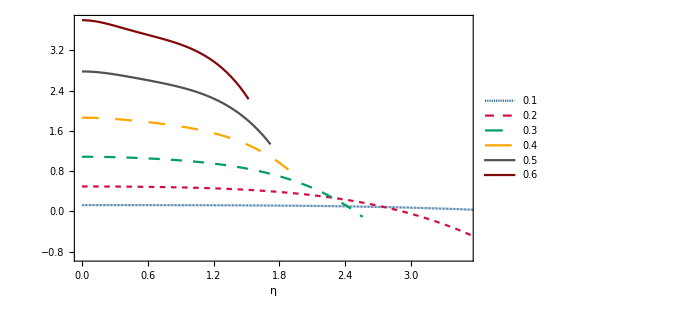

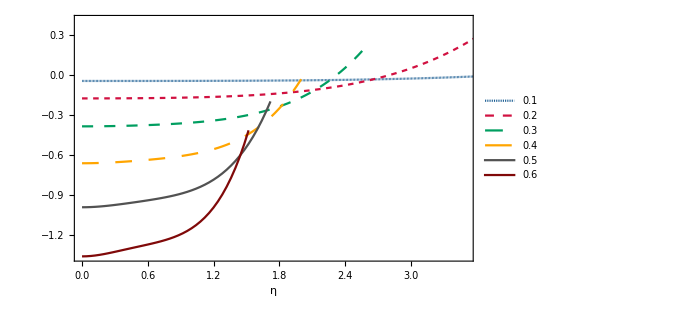

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.7}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

### Iso-breaking in DF approximation

#### Axial modes

```mathematica
Ta={{{0,0.24873526079596356-0.09254971556771212 ⅈ},{1/25+ⅈ/25,0.24873526115655725-0.09254971526426195 ⅈ},{2/25+(2 ⅈ)/25,0.2487352622392533-0.0925497143544262 ⅈ},{3/25+(3 ⅈ)/25,0.24873526404679705-0.09254971283974874 ⅈ},{4/25+(4 ⅈ)/25,0.24873526658376421-0.09254971072280219 ⅈ},{1/5+ⅈ/5,0.24873526985656172-0.09254970800718697 ⅈ},{6/25+(6 ⅈ)/25,0.24873527387342828-0.09254970469752997 ⅈ},{7/25+(7 ⅈ)/25,0.24873527864443515-0.09254970079948308 ⅈ},{8/25+(8 ⅈ)/25,0.24873528418148758-0.09254969631972096 ⅈ},{9/25+(9 ⅈ)/25,0.24873529049832618-0.09254969126593902 ⅈ},{2/5+(2 ⅈ)/5,0.24873529761052804-0.09254968564685054 ⅈ},{11/25+(11 ⅈ)/25,0.24873530553550918-0.09254967947218351 ⅈ},{12/25+(12 ⅈ)/25,0.24873531429252588-0.09254967275267743 ⅈ},{13/25+(13 ⅈ)/25,0.24873532390267714-0.09254966550007931 ⅈ},{14/25+(14 ⅈ)/25,0.24873533438890735-0.09254965772713962 ⅈ},{3/5+(3 ⅈ)/5,0.24873534577600817-0.09254964944760782 ⅈ},{16/25+(16 ⅈ)/25,0.24873535809062217-0.09254964067622726 ⅈ},{17/25+(17 ⅈ)/25,0.248735371361245-0.09254963142873004 ⅈ},{18/25+(18 ⅈ)/25,0.2487353856182292-0.09254962172183145 ⅈ},{19/25+(19 ⅈ)/25,0.24873540089378743-0.09254961157322378 ⅈ},{4/5+(4 ⅈ)/5,0.2487354172219958-0.09254960100157 ⅈ},{21/25+(21 ⅈ)/25,0.24873543463879794-0.09254959002649706 ⅈ},{22/25+(22 ⅈ)/25,0.24873545318200893-0.0925495786685886 ⅈ},{23/25+(23 ⅈ)/25,0.2487354728913192-0.09254956694937758 ⅈ},{24/25+(24 ⅈ)/25,0.24873549380829943-0.0925495548913381 ⅈ},{1+ⅈ,0.24873551597640461-0.09254954251787752 ⅈ},{26/25+(26 ⅈ)/25,0.24873553944097898-0.09254952985332725 ⅈ},{27/25+(27 ⅈ)/25,0.2487355642492609-0.09254951692293403 ⅈ},{28/25+(28 ⅈ)/25,0.24873559045038807-0.09254950375285036 ⅈ},{29/25+(29 ⅈ)/25,0.2487356180954027-0.09254949037012448 ⅈ},{6/5+(6 ⅈ)/5,0.2487356472372569-0.09254947680269018 ⅈ},{31/25+(31 ⅈ)/25,0.24873567793081852-0.0925494630793561 ⅈ},{32/25+(32 ⅈ)/25,0.248735710232877-0.0925494492297947 ⅈ},{33/25+(33 ⅈ)/25,0.24873574420214906-0.09254943528453062 ⅈ},{34/25+(34 ⅈ)/25,0.24873577989928497-0.09254942127492871 ⅈ},{7/5+(7 ⅈ)/5,0.24873581738687514-0.09254940723318192 ⅈ},{36/25+(36 ⅈ)/25,0.24873585672945628-0.09254939319229816 ⅈ},{37/25+(37 ⅈ)/25,0.24873589799351803-0.09254937918608747 ⅈ},{38/25+(38 ⅈ)/25,0.24873594124751006-0.09254936524914807 ⅈ},{39/25+(39 ⅈ)/25,0.24873598656184878-0.0925493514168526 ⅈ},{8/5+(8 ⅈ)/5,0.24873603400892438-0.09254933772533326 ⅈ},{41/25+(41 ⅈ)/25,0.24873608366310837-0.09254932421146714 ⅈ},{42/25+(42 ⅈ)/25,0.24873613560076058-0.09254931091286063 ⅈ},{43/25+(43 ⅈ)/25,0.248736189900237-0.09254929786783374 ⅈ},{44/25+(44 ⅈ)/25,0.24873624664189717-0.09254928511540363 ⅈ},{9/5+(9 ⅈ)/5,0.2487363059081123-0.09254927269526782 ⅈ},{46/25+(46 ⅈ)/25,0.24873636778327288-0.0925492606477871 ⅈ},{47/25+(47 ⅈ)/25,0.2487364323537967-0.09254924901396773 ⅈ},{48/25+(48 ⅈ)/25,0.24873649970813733-0.09254923783544317 ⅈ},{49/25+(49 ⅈ)/25,0.2487365699367918-0.09254922715445547 ⅈ},{2+2 ⅈ,0.24873664313230973-0.09254921701383617 ⅈ},{51/25+(51 ⅈ)/25,0.24873671938930103-0.09254920745698644 ⅈ},{52/25+(52 ⅈ)/25,0.2487367988044449-0.09254919852785719 ⅈ},{53/25+(53 ⅈ)/25,0.24873688147649825-0.0925491902709281 ⅈ},{54/25+(54 ⅈ)/25,0.2487369675063049-0.09254918273118672 ⅈ},{11/5+(11 ⅈ)/5,0.24873705699680346-0.09254917595410662 ⅈ},{56/25+(56 ⅈ)/25,0.2487371500530372-0.09254916998562522 ⅈ},{57/25+(57 ⅈ)/25,0.24873724678216236-0.09254916487212099 ⅈ},{58/25+(58 ⅈ)/25,0.24873734729345762-0.09254916066039028 ⅈ},{59/25+(59 ⅈ)/25,0.24873745169833247-0.09254915739762345 ⅈ},{12/5+(12 ⅈ)/5,0.2487375601103369-0.09254915513138047 ⅈ},{61/25+(61 ⅈ)/25,0.24873767264517063-0.092549153909566 ⅈ},{62/25+(62 ⅈ)/25,0.24873778942069158-0.09254915378040406 ⅈ},{63/25+(63 ⅈ)/25,0.2487379105569257-0.09254915479241173 ⅈ},{64/25+(64 ⅈ)/25,0.24873803617607607-0.09254915699437279 ⅈ},{13/5+(13 ⅈ)/5,0.2487381664025319-0.09254916043531035 ⅈ},{66/25+(66 ⅈ)/25,0.24873830136287778-0.0925491651644592 ⅈ},{67/25+(67 ⅈ)/25,0.24873844118590308-0.09254917123123732 ⅈ},{68/25+(68 ⅈ)/25,0.24873858600261098-0.09254917868521699 ⅈ},{69/25+(69 ⅈ)/25,0.24873873594622772-0.09254918757609522 ⅈ},{14/5+(14 ⅈ)/5,0.24873889115221162-0.09254919795366344 ⅈ},{71/25+(71 ⅈ)/25,0.2487390517582622-0.09254920986777689 ⅈ},{72/25+(72 ⅈ)/25,0.2487392179043292-0.09254922336832298 ⅈ},{73/25+(73 ⅈ)/25,0.24873938973262164-0.09254923850518942 ⅈ},{74/25+(74 ⅈ)/25,0.24873956738761668-0.09254925532823133 ⅈ},{3+3 ⅈ,0.248739751016068-0.09254927388723794 ⅈ},{76/25+(76 ⅈ)/25,0.2487399407670153-0.09254929423189867 ⅈ},{77/25+(77 ⅈ)/25,0.24874013679179205-0.09254931641176833 ⅈ},{78/25+(78 ⅈ)/25,0.24874033924403452-0.09254934047623188 ⅈ},{79/25+(79 ⅈ)/25,0.24874054827968997-0.09254936647446822 ⅈ},{16/5+(16 ⅈ)/5,0.2487407640570247-0.09254939445541378 ⅈ},{81/25+(81 ⅈ)/25,0.24874098673663214-0.09254942446772484 ⅈ},{82/25+(82 ⅈ)/25,0.24874121648144093-0.09254945655973962 ⅈ},{83/25+(83 ⅈ)/25,0.24874145345672236-0.09254949077943934 ⅈ},{84/25+(84 ⅈ)/25,0.24874169783009778-0.09254952717440885 ⅈ},{17/5+(17 ⅈ)/5,0.24874194977154623-0.09254956579179632 ⅈ},{86/25+(86 ⅈ)/25,0.248742209453411-0.09254960667827222 ⅈ},{87/25+(87 ⅈ)/25,0.2487424770504069-0.09254964987998777 ⅈ},{88/25+(88 ⅈ)/25,0.24874275273962665-0.09254969544253232 ⅈ},{89/25+(89 ⅈ)/25,0.2487430367005469-0.0925497434108904 ⅈ},{18/5+(18 ⅈ)/5,0.24874332911503458-0.09254979382939753 ⅈ},{91/25+(91 ⅈ)/25,0.24874363016735254-0.09254984674169568 ⅈ},{92/25+(92 ⅈ)/25,0.2487439400441646-0.09254990219068782 ⅈ},{93/25+(93 ⅈ)/25,0.24874425893454108-0.09254996021849153 ⅈ},{94/25+(94 ⅈ)/25,0.24874458702996294-0.09255002086639214 ⅈ},{19/5+(19 ⅈ)/5,0.24874492452432664-0.09255008417479473 ⅈ},{96/25+(96 ⅈ)/25,0.24874527161394763-0.09255015018317574 ⅈ},{97/25+(97 ⅈ)/25,0.24874562849756401-0.09255021893003336 ⅈ},{98/25+(98 ⅈ)/25,0.2487459953763398-0.09255029045283747 ⅈ},{99/25+(99 ⅈ)/25,0.24874637245386713-0.09255036478797847 ⅈ},{4+4 ⅈ,0.24874675993616882-0.09255044197071555 ⅈ},{101/25+(101 ⅈ)/25,0.24874715803169994-0.09255052203512393 ⅈ},{102/25+(102 ⅈ)/25,0.24874756695134878-0.09255060501404143 ⅈ},{103/25+(103 ⅈ)/25,0.24874798690843786-0.09255069093901405 ⅈ},{104/25+(104 ⅈ)/25,0.24874841811872356-0.09255077984024095 ⅈ},{21/5+(21 ⅈ)/5,0.2487488608003961-0.09255087174651815 ⅈ},{106/25+(106 ⅈ)/25,0.24874931517407792-0.09255096668518199 ⅈ},{107/25+(107 ⅈ)/25,0.2487497814628224-0.09255106468205114 ⅈ},{108/25+(108 ⅈ)/25,0.24875025989211139-0.09255116576136815 ⅈ},{109/25+(109 ⅈ)/25,0.24875075068985186-0.09255126994574008 ⅈ},{22/5+(22 ⅈ)/5,0.2487512540863726-0.09255137725607795 ⅈ},{111/25+(111 ⅈ)/25,0.2487517703144197-0.09255148771153583 ⅈ},{112/25+(112 ⅈ)/25,0.2487522996091507-0.09255160132944859 ⅈ},{113/25+(113 ⅈ)/25,0.2487528422081296-0.09255171812526922 ⅈ},{114/25+(114 ⅈ)/25,0.24875339835131932-0.09255183811250478 ⅈ},{23/5+(23 ⅈ)/5,0.24875396828107432-0.09255196130265193 ⅈ},{116/25+(116 ⅈ)/25,0.24875455224213217-0.09255208770513125 ⅈ},{117/25+(117 ⅈ)/25,0.24875515048160401-0.09255221732722103 ⅈ},{118/25+(118 ⅈ)/25,0.2487557632489644-0.09255235017398976 ⅈ},{119/25+(119 ⅈ)/25,0.24875639079604006-0.092552486248228 ⅈ},{24/5+(24 ⅈ)/5,0.2487570333769975-0.09255262555037948 ⅈ},{121/25+(121 ⅈ)/25,0.24875769124832986-0.092552768078471 ⅈ},{122/25+(122 ⅈ)/25,0.2487583646688427-0.0925529138280418 ⅈ},{123/25+(123 ⅈ)/25,0.24875905389963848-0.09255306279207164 ⅈ},{124/25+(124 ⅈ)/25,0.24875975920410018-0.09255321496090868 ⅈ},{5+5 ⅈ,0.24876048084787358-0.09255337032219568 ⅈ},{126/25+(126 ⅈ)/25,0.24876121909884863-0.09255352886079594 ⅈ},{127/25+(127 ⅈ)/25,0.24876197422713922-0.09255369055871818 ⅈ},{128/25+(128 ⅈ)/25,0.24876274650506208-0.09255385539504064 ⅈ},{129/25+(129 ⅈ)/25,0.24876353620711394-0.0925540233458341 ⅈ},{26/5+(26 ⅈ)/5,0.24876434360994829-0.09255419438408448 ⅈ},{131/25+(131 ⅈ)/25,0.24876516899234918-0.0925543684796142 ⅈ},{132/25+(132 ⅈ)/25,0.24876601263520542-0.09255454559900299 ⅈ},{133/25+(133 ⅈ)/25,0.24876687482148208-0.09255472570550786 ⅈ},{134/25+(134 ⅈ)/25,0.24876775583619104-0.09255490875898213 ⅈ},{27/5+(27 ⅈ)/5,0.2487686559663598-0.09255509471579385 ⅈ},{136/25+(136 ⅈ)/25,0.24876957550099904-0.09255528352874332 ⅈ},{137/25+(137 ⅈ)/25,0.24877051473106826-0.09255547514697984 ⅈ},{138/25+(138 ⅈ)/25,0.24877147394943985-0.09255566951591805 ⅈ},{139/25+(139 ⅈ)/25,0.24877245345086166-0.09255586657715283 ⅈ},{28/5+(28 ⅈ)/5,0.2487734535319177-0.09255606626837441 ⅈ},{141/25+(141 ⅈ)/25,0.24877447449098708-0.09255626852328191 ⅈ},{142/25+(142 ⅈ)/25,0.2487755166282008-0.09255647327149688 ⅈ},{143/25+(143 ⅈ)/25,0.2487765802453978-0.09255668043847581 ⅈ},{144/25+(144 ⅈ)/25,0.2487776656460776-0.09255688994542208 ⅈ},{29/5+(29 ⅈ)/5,0.24877877313535193-0.09255710170919736 ⅈ},{146/25+(146 ⅈ)/25,0.2487799030198946-0.09255731564223245 ⅈ},{147/25+(147 ⅈ)/25,0.24878105560788827-0.09255753165243748 ⅈ},{148/25+(148 ⅈ)/25,0.2487822312089701-0.09255774964311163 ⅈ},{149/25+(149 ⅈ)/25,0.24878343013417495-0.09255796951285226 ⅈ},{6+6 ⅈ,0.2487846526958762-0.09255819115546376 ⅈ},{151/25+(151 ⅈ)/25,0.248785899207725-0.09255841445986576 ⅈ},{152/25+(152 ⅈ)/25,0.24878716998458592-0.09255863931000109 ⅈ},{153/25+(153 ⅈ)/25,0.248788465342472-0.0925588655847432 ⅈ},{154/25+(154 ⅈ)/25,0.2487897855984762-0.09255909315780338 ⅈ},{31/5+(31 ⅈ)/5,0.2487911310707008-0.09255932189763776 ⅈ},{156/25+(156 ⅈ)/25,0.24879250207818432-0.09255955166735369 ⅈ},{157/25+(157 ⅈ)/25,0.24879389894082587-0.0925597823246165 ⅈ},{158/25+(158 ⅈ)/25,0.24879532197930737-0.09256001372155538 ⅈ},{159/25+(159 ⅈ)/25,0.2487967715150123-0.09256024570466978 ⅈ},{32/5+(32 ⅈ)/5,0.24879824786994265-0.09256047811473538 ⅈ},{161/25+(161 ⅈ)/25,0.24879975136663238-0.09256071078671008 ⅈ},{162/25+(162 ⅈ)/25,0.24880128232805904-0.09256094354963999 ⅈ},{163/25+(163 ⅈ)/25,0.2488028410775516-0.09256117622656584 ⅈ},{164/25+(164 ⅈ)/25,0.2488044279386962-0.09256140863442883 ⅈ},{33/5+(33 ⅈ)/5,0.24880604323523847-0.09256164058397748 ⅈ},{166/25+(166 ⅈ)/25,0.24880768729098324-0.0925618718796741 ⅈ},{167/25+(167 ⅈ)/25,0.24880936042969085-0.09256210231960199 ⅈ},{168/25+(168 ⅈ)/25,0.24881106297497113-0.09256233169537272 ⅈ},{169/25+(169 ⅈ)/25,0.24881279525017336-0.09256255979203412 ⅈ},{34/5+(34 ⅈ)/5,0.2488145575782738-0.09256278638797862 ⅈ},{171/25+(171 ⅈ)/25,0.24881635028175972-0.09256301125485225 ⅈ},{172/25+(172 ⅈ)/25,0.24881817368251033-0.09256323415746434 ⅈ},{173/25+(173 ⅈ)/25,0.2488200281016742-0.09256345485369788 ⅈ},{174/25+(174 ⅈ)/25,0.24882191385954364-0.09256367309442076 ⅈ},{7+7 ⅈ,0.24882383127542543-0.092563888623398 ⅈ},{176/25+(176 ⅈ)/25,0.2488257806675087-0.09256410117720482 ⅈ},{177/25+(177 ⅈ)/25,0.24882776235272858-0.09256431048514077 ⅈ},{178/25+(178 ⅈ)/25,0.248829776646627-0.0925645162691455 ⅈ}},{{0,0.2501443357495142-0.092735681736817 ⅈ},{1/25+ⅈ/25,0.25014434151086595-0.09273567699822176 ⅈ},{2/25+(2 ⅈ)/25,0.25014435880855485-0.09273566278964847 ⅈ},{3/25+(3 ⅈ)/25,0.2501443876834873-0.0927356391327234 ⅈ},{4/25+(4 ⅈ)/25,0.2501444282038611-0.09273560606345355 ⅈ},{1/5+ⅈ/5,0.2501444804651953-0.0927355636321713 ⅈ},{6/25+(6 ⅈ)/25,0.2501445445903724-0.09273551190345701 ⅈ},{7/25+(7 ⅈ)/25,0.25014462072969296-0.09273545095603927 ⅈ},{8/25+(8 ⅈ)/25,0.25014470906094066-0.09273538088267258 ⅈ},{9/25+(9 ⅈ)/25,0.250144809789461-0.09273530178999258 ⅈ},{2/5+(2 ⅈ)/5,0.25014492314825015-0.09273521379834859 ⅈ},{11/25+(11 ⅈ)/25,0.2501450493980555-0.0927351170416129 ⅈ},{12/25+(12 ⅈ)/25,0.2501451888274882-0.09273501166696693 ⅈ},{13/25+(13 ⅈ)/25,0.2501453417531464-0.09273489783466424 ⅈ},{14/25+(14 ⅈ)/25,0.2501455085197486-0.09273477571776897 ⅈ},{3/5+(3 ⅈ)/5,0.250145689500279-0.09273464550187112 ⅈ},{16/25+(16 ⅈ)/25,0.2501458850961423-0.0927345073847765 ⅈ},{17/25+(17 ⅈ)/25,0.2501460957373285-0.09273436157617237 ⅈ},{18/25+(18 ⅈ)/25,0.25014632188258845-0.0927342082972676 ⅈ},{19/25+(19 ⅈ)/25,0.2501465640196175-0.09273404778040714 ⅈ},{4/5+(4 ⅈ)/5,0.2501468226652487-0.09273388026866046 ⅈ},{21/25+(21 ⅈ)/25,0.2501470983656553-0.09273370601538312 ⅈ},{22/25+(22 ⅈ)/25,0.2501473916965602-0.09273352528375142 ⅈ},{23/25+(23 ⅈ)/25,0.25014770326345404-0.09273333834626907 ⅈ},{24/25+(24 ⅈ)/25,0.25014803370182-0.09273314548424601 ⅈ},{1+ⅈ,0.2501483836773656-0.09273294698724777 ⅈ},{26/25+(26 ⅈ)/25,0.25014875388626007-0.09273274315251592 ⅈ},{27/25+(27 ⅈ)/25,0.250149145055378-0.09273253428435808 ⅈ},{28/25+(28 ⅈ)/25,0.25014955794254673-0.09273232069350724 ⅈ},{29/25+(29 ⅈ)/25,0.25014999333679855-0.09273210269644948 ⅈ},{6/5+(6 ⅈ)/5,0.25015045205862624-0.0927318806147198 ⅈ},{31/25+(31 ⅈ)/25,0.25015093496024055-0.0927316547741647 ⅈ},{32/25+(32 ⅈ)/25,0.2501514429258299-0.09273142550417134 ⅈ},{33/25+(33 ⅈ)/25,0.25015197687182106-0.0927311931368621 ⅈ},{34/25+(34 ⅈ)/25,0.25015253774713836-0.09273095800625407 ⅈ},{7/5+(7 ⅈ)/5,0.2501531265334634-0.09273072044738251 ⅈ},{36/25+(36 ⅈ)/25,0.25015374424549136-0.09273048079538726 ⅈ},{37/25+(37 ⅈ)/25,0.25015439193118394-0.0927302393845618 ⅈ},{38/25+(38 ⅈ)/25,0.2501550706720187-0.09272999654736364 ⅈ},{39/25+(39 ⅈ)/25,0.25015578158323065-0.09272975261338517 ⅈ},{8/5+(8 ⅈ)/5,0.2501565258140483-0.09272950790828483 ⅈ},{41/25+(41 ⅈ)/25,0.2501573045479203-0.09272926275267658 ⅈ},{42/25+(42 ⅈ)/25,0.25015811900273166-0.09272901746097793 ⅈ},{43/25+(43 ⅈ)/25,0.2501589704310089-0.09272877234021477 ⅈ},{44/25+(44 ⅈ)/25,0.25015986012011093-0.09272852768878291 ⅈ},{9/5+(9 ⅈ)/5,0.25016078939240555-0.09272828379516482 ⅈ},{46/25+(46 ⅈ)/25,0.2501617596054283-0.09272804093660114 ⅈ},{47/25+(47 ⅈ)/25,0.2501627721520225-0.09272779937771601 ⅈ},{48/25+(48 ⅈ)/25,0.2501638284604586-0.09272755936909535 ⅈ},{49/25+(49 ⅈ)/25,0.25016492999452977-0.09272732114581764 ⅈ},{2+2 ⅈ,0.2501660782536226-0.09272708492593551 ⅈ},{51/25+(51 ⅈ)/25,0.2501672747727594-0.09272685090890889 ⅈ},{52/25+(52 ⅈ)/25,0.25016852112261134-0.09272661927398766 ⅈ},{53/25+(53 ⅈ)/25,0.25016981890947726-0.09272639017854396 ⅈ},{54/25+(54 ⅈ)/25,0.25017116977522785-0.09272616375635329 ⅈ},{11/5+(11 ⅈ)/5,0.25017257539721177-0.09272594011582393 ⅈ},{56/25+(56 ⅈ)/25,0.25017403748811934-0.09272571933817404 ⅈ},{57/25+(57 ⅈ)/25,0.25017555779580264-0.09272550147555653 ⅈ},{58/25+(58 ⅈ)/25,0.2501771381030475-0.09272528654913086 ⅈ},{59/25+(59 ⅈ)/25,0.2501787802272946-0.09272507454708175 ⅈ},{12/5+(12 ⅈ)/5,0.25018048602030624-0.09272486542258487 ⅈ},{61/25+(61 ⅈ)/25,0.25018225736777444-0.09272465909171922 ⅈ},{62/25+(62 ⅈ)/25,0.2501840961888678-0.09272445543132636 ⅈ},{63/25+(63 ⅈ)/25,0.2501860044357114-0.09272425427681705 ⅈ},{64/25+(64 ⅈ)/25,0.250187984092798-0.09272405541992525 ⅈ},{13/5+(13 ⅈ)/5,0.2501900371763242-0.09272385860641036 ⅈ},{66/25+(66 ⅈ)/25,0.2501921657334484-0.0927236635337082 ⅈ},{67/25+(67 ⅈ)/25,0.2501943718414651-0.09272346984853182 ⅈ},{68/25+(68 ⅈ)/25,0.25019665760689314-0.09272327714442309 ⅈ},{69/25+(69 ⅈ)/25,0.25019902516446874-0.09272308495925656 ⅈ},{14/5+(14 ⅈ)/5,0.2502014766760438-0.09272289277269682 ⅈ},{71/25+(71 ⅈ)/25,0.2502040143293798-0.09272270000361187 ⅈ},{72/25+(72 ⅈ)/25,0.2502066403368344-0.09272250600744324 ⅈ},{73/25+(73 ⅈ)/25,0.25020935693393553-0.09272231007353696 ⅈ},{74/25+(74 ⅈ)/25,0.25021216637783605-0.09272211142243637 ⅈ},{3+3 ⅈ,0.25021507094564444-0.09272190920314091 ⅈ},{76/25+(76 ⅈ)/25,0.2502180729326257-0.09272170249033349 ⅈ},{77/25+(77 ⅈ)/25,0.2502211746502667-0.09272149028158065 ⅈ},{78/25+(78 ⅈ)/25,0.2502243784241997-0.09272127149450902 ⅈ},{79/25+(79 ⅈ)/25,0.2502276865919783-0.0927210449639631 ⅈ},{16/5+(16 ⅈ)/5,0.2502311015007004-0.09272080943914872 ⅈ},{81/25+(81 ⅈ)/25,0.25023462550447084-0.09272056358076802 ⅈ},{82/25+(82 ⅈ)/25,0.25023826096169915-0.09272030595815138 ⅈ},{83/25+(83 ⅈ)/25,0.2502420102322253-0.09272003504639291 ⅈ},{84/25+(84 ⅈ)/25,0.2502458756742677-0.092719749223496 ⅈ},{17/5+(17 ⅈ)/5,0.250249859641188-0.0927194467675369 ⅈ},{86/25+(86 ⅈ)/25,0.2502539644780658-0.09271912585385343 ⅈ},{87/25+(87 ⅈ)/25,0.25025819251807874-0.09271878455226806 ⅈ},{88/25+(88 ⅈ)/25,0.250262546078681-0.09271842082435443 ⅈ},{89/25+(89 ⅈ)/25,0.25026702745757623-0.09271803252075668 ⅈ},{18/5+(18 ⅈ)/5,0.25027163892847853-0.0927176173785724 ⅈ},{91/25+(91 ⅈ)/25,0.2502763827366577-0.09271717301881018 ⅈ}},{{0,0.25247008568318147-0.09304542175842358 ⅈ},{1/25+ⅈ/25,0.25247011477042824-0.09304539872143626 ⅈ},{2/25+(2 ⅈ)/25,0.25247020209333515-0.09304532963868327 ⅈ},{3/25+(3 ⅈ)/25,0.2524703478354588-0.09304521459467352 ⅈ},{4/25+(4 ⅈ)/25,0.25247055230291865-0.09304505372986131 ⅈ},{1/5+ⅈ/5,0.25247081592468273-0.09304484724005459 ⅈ},{6/25+(6 ⅈ)/25,0.2524711392529666-0.0930445953755838 ⅈ},{7/25+(7 ⅈ)/25,0.25247152296374403-0.09304429844022981 ⅈ},{8/25+(8 ⅈ)/25,0.25247196785736525-0.09304395678990739 ⅈ},{9/25+(9 ⅈ)/25,0.25247247485928326-0.09304357083110074 ⅈ},{2/5+(2 ⅈ)/5,0.25247304502088186-0.09304314101904751 ⅈ},{11/25+(11 ⅈ)/25,0.2524736795204035-0.09304266785566498 ⅈ},{12/25+(12 ⅈ)/25,0.2524743796639724-0.09304215188721505 ⅈ},{13/25+(13 ⅈ)/25,0.25247514688670675-0.0930415937016997 ⅈ},{14/25+(14 ⅈ)/25,0.25247598275391664-0.09304099392598154 ⅈ},{3/5+(3 ⅈ)/5,0.2524768889623782-0.093040353222622 ⅈ},{16/25+(16 ⅈ)/25,0.2524778673416797-0.09303967228642847 ⅈ},{17/25+(17 ⅈ)/25,0.2524789198556307-0.09303895184070264 ⅈ},{18/25+(18 ⅈ)/25,0.2524800486037246-0.09303819263318021 ⅈ},{19/25+(19 ⅈ)/25,0.25248125582264586-0.09303739543165307 ⅈ},{4/5+(4 ⅈ)/5,0.25248254388781194-0.09303656101926272 ⅈ},{21/25+(21 ⅈ)/25,0.252483915314936-0.09303569018945536 ⅈ},{22/25+(22 ⅈ)/25,0.2524853727616-0.09303478374058621 ⅈ},{23/25+(23 ⅈ)/25,0.25248691902882214-0.09303384247016247 ⅈ},{24/25+(24 ⅈ)/25,0.25248855706260526-0.09303286716871216 ⅈ},{1+ⅈ,0.2524902899554473-0.09303185861326677 ⅈ},{26/25+(26 ⅈ)/25,0.25249212094779777-0.0930308175604448 ⅈ},{27/25+(27 ⅈ)/25,0.2524940534294389-0.09302974473912352 ⅈ},{28/25+(28 ⅈ)/25,0.2524960909407709-0.0930286408426854 ⅈ},{29/25+(29 ⅈ)/25,0.25249823717397785-0.09302750652082653 ⅈ},{6/5+(6 ⅈ)/5,0.2525004959740489-0.09302634237091333 ⅈ},{31/25+(31 ⅈ)/25,0.25250287133962857-0.09302514892887487 ⅈ},{32/25+(32 ⅈ)/25,0.252505367423665-0.09302392665961792 ⅈ},{33/25+(33 ⅈ)/25,0.25250798853382717-0.09302267594695202 ⅈ},{34/25+(34 ⅈ)/25,0.2525107391326548-0.09302139708301278 ⅈ},{7/5+(7 ⅈ)/5,0.25251362383740633-0.09302009025717238 ⅈ},{36/25+(36 ⅈ)/25,0.2525166474195644-0.09301875554442636 ⅈ},{37/25+(37 ⅈ)/25,0.2525198148039588-0.09301739289324802 ⅈ},{38/25+(38 ⅈ)/25,0.25252313106745966-0.09301600211290226 ⅈ},{39/25+(39 ⅈ)/25,0.2525266014371967-0.09301458286021179 ⅈ},{8/5+(8 ⅈ)/5,0.25253023128824975-0.09301313462577238 ⅈ},{41/25+(41 ⅈ)/25,0.2525340261407593-0.09301165671961398 ⅈ},{42/25+(42 ⅈ)/25,0.2525379916563996-0.09301014825630739 ⅈ},{43/25+(43 ⅈ)/25,0.25254213363415096-0.09300860813952086 ⅈ},{44/25+(44 ⅈ)/25,0.25254645800531034-0.09300703504603135 ⅈ},{9/5+(9 ⅈ)/5,0.25255097082767075-0.0930054274092013 ⅈ},{46/25+(46 ⅈ)/25,0.2525556782787977-0.09300378340193483 ⅈ},{47/25+(47 ⅈ)/25,0.2525605866483297-0.0930021009191322 ⅈ},{48/25+(48 ⅈ)/25,0.2525657023292232-0.09300037755966643 ⅈ},{49/25+(49 ⅈ)/25,0.25257103180786045-0.09299861060791227 ⅈ},{2+2 ⅈ,0.2525765816529366-0.09299679701486362 ⅈ},{51/25+(51 ⅈ)/25,0.2525823585030375-0.09299493337888323 ⅈ},{52/25+(52 ⅈ)/25,0.2525883690528171-0.09299301592613549 ⅈ},{53/25+(53 ⅈ)/25,0.25259462003768285-0.09299104049076277 ⅈ},{54/25+(54 ⅈ)/25,0.2526011182168934-0.09298900249487414 ⅈ},{11/5+(11 ⅈ)/5,0.25260787035497145-0.09298689692842588 ⅈ},{56/25+(56 ⅈ)/25,0.25261488320133624-0.09298471832908425 ⅈ},{57/25+(57 ⅈ)/25,0.25262216346805644-0.09298246076217266 ⅈ},{58/25+(58 ⅈ)/25,0.2526297178056276-0.0929801178008181 ⅈ},{59/25+(59 ⅈ)/25,0.25263755277667893-0.09297768250642457 ⅈ},{12/5+(12 ⅈ)/5,0.2526456748275169-0.09297514740961733 ⅈ},{61/25+(61 ⅈ)/25,0.25265409025741775-0.09297250449181435 ⅈ},{62/25+(62 ⅈ)/25,0.25266280518558626-0.09296974516760009 ⅈ},{63/25+(63 ⅈ)/25,0.2526718255157057-0.09296686026809069 ⅈ},{64/25+(64 ⅈ)/25,0.2526811568980123-0.09296384002549897 ⅈ}},{{0,0.25567960789894006-0.09347825427830223 ⅈ},{1/25+ⅈ/25,0.2556796994122349-0.09347818548137884 ⅈ},{2/25+(2 ⅈ)/25,0.2556799741146002-0.09347797914515468 ⅈ},{3/25+(3 ⅈ)/25,0.25568043249372013-0.09347763543265554 ⅈ},{4/25+(4 ⅈ)/25,0.25568107536320733-0.09347715461354542 ⅈ},{1/5+ⅈ/5,0.25568190386380274-0.09347653706104911 ⅈ},{6/25+(6 ⅈ)/25,0.2556829194650411-0.09347578324762379 ⅈ},{7/25+(7 ⅈ)/25,0.2556841239673653-0.09347489373936033 ⅈ},{8/25+(8 ⅈ)/25,0.25568551950466945-0.09347386918909009 ⅈ},{9/25+(9 ⅈ)/25,0.2556871085472467-0.09347271032816563 ⅈ},{2/5+(2 ⅈ)/5,0.2556888939051078-0.09347141795688015 ⅈ},{11/25+(11 ⅈ)/25,0.25569087873163787-0.09346999293348426 ⅈ},{12/25+(12 ⅈ)/25,0.2556930665275452-0.09346843616175338 ⅈ},{13/25+(13 ⅈ)/25,0.2556954611450548-0.09346674857705417 ⅈ},{14/25+(14 ⅈ)/25,0.25569806679228857-0.09346493113085334 ⅈ},{3/5+(3 ⅈ)/5,0.25570088803776764-0.09346298477360757 ⅈ},{16/25+(16 ⅈ)/25,0.25570392981496376-0.0934609104359679 ⅈ},{17/25+(17 ⅈ)/25,0.25570719742681575-0.09345870900822927 ⅈ},{18/25+(18 ⅈ)/25,0.2557106965501177-0.09345638131795027 ⅈ},{19/25+(19 ⅈ)/25,0.2557144332396753-0.09345392810566606 ⅈ},{4/5+(4 ⅈ)/5,0.25571841393210987-0.09345134999861376 ⅈ},{21/25+(21 ⅈ)/25,0.2557226454491835-0.09344864748238844 ⅈ},{22/25+(22 ⅈ)/25,0.25572713500049504-0.09344582087044442 ⅈ},{23/25+(23 ⅈ)/25,0.25573189018538917-0.09344287027135956 ⅈ},{24/25+(24 ⅈ)/25,0.2557369189938975-0.09343979555377672 ⅈ},{1+ⅈ,0.25574222980651373-0.09343659630894244 ⅈ},{26/25+(26 ⅈ)/25,0.2557478313925867-0.09343327181076384 ⅈ},{27/25+(27 ⅈ)/25,0.2557537329070905-0.0934298209733113 ⅈ},{28/25+(28 ⅈ)/25,0.2557599438855083-0.09342624230570166 ⅈ},{29/25+(29 ⅈ)/25,0.25576647423654464-0.0934225338643064 ⅈ},{6/5+(6 ⅈ)/5,0.2557733342323504-0.09341869320224142 ⅈ},{31/25+(31 ⅈ)/25,0.25578053449592064-0.09341471731611219 ⅈ},{32/25+(32 ⅈ)/25,0.25578808598529457-0.0934106025900047 ⅈ},{33/25+(33 ⅈ)/25,0.2557959999741587-0.09340634473673887 ⅈ},{34/25+(34 ⅈ)/25,0.25580428802842037-0.09340193873642602 ⅈ},{7/5+(7 ⅈ)/5,0.2558129619782911-0.09339737877240681 ⅈ},{36/25+(36 ⅈ)/25,0.25582203388538377-0.09339265816468359 ⅈ},{37/25+(37 ⅈ)/25,0.25583151600429777-0.09338776930100538 ⅈ},{38/25+(38 ⅈ)/25,0.25584142073813576-0.0933827035658164 ⅈ},{39/25+(39 ⅈ)/25,0.25585176058736403-0.09337745126733661 ⅈ},{8/5+(8 ⅈ)/5,0.25586254809140396-0.09337200156311055 ⅈ},{41/25+(41 ⅈ)/25,0.25587379576231684-0.09336634238443711 ⅈ},{42/25+(42 ⅈ)/25,0.2558855160099254-0.09336046036017644 ⅈ},{43/25+(43 ⅈ)/25,0.2558977210577032-0.09335434074052745 ⅈ},{44/25+(44 ⅈ)/25,0.255910422848756-0.09334796732147231 ⅈ},{9/5+(9 ⅈ)/5,0.2559236329412264-0.0933413223707022 ⅈ},{46/25+(46 ⅈ)/25,0.255937362392466-0.09333438655596352 ⅈ},{47/25+(47 ⅈ)/25,0.2559516216313523-0.09332713887690187 ⅈ},{48/25+(48 ⅈ)/25,0.25596642031817285-0.0933195566016273 ⅈ},{49/25+(49 ⅈ)/25,0.25598176719156795-0.09331161520938011 ⅈ},{2+2 ⅈ,0.25599766990211364-0.09330328834084099 ⅈ}},{{0,0.259729037431041-0.09403255764314543 ⅈ},{1/25+ⅈ/25,0.2597292593123827-0.09403240148073533 ⅈ},{2/25+(2 ⅈ)/25,0.25972992527067246-0.09403193302673178 ⅈ},{3/25+(3 ⅈ)/25,0.25973103624928606-0.0940311523786728 ⅈ},{4/25+(4 ⅈ)/25,0.25973259382244773-0.09403005969196557 ⅈ},{1/5+ⅈ/5,0.25973460019808264-0.09402865516910422 ⅈ},{6/25+(6 ⅈ)/25,0.2597370582217293-0.09402693904447972 ⅈ},{7/25+(7 ⅈ)/25,0.25973997138142024-0.0940249115646851 ⅈ},{8/25+(8 ⅈ)/25,0.25974334381342185-0.09402257296419543 ⅈ},{9/25+(9 ⅈ)/25,0.25974718030868654-0.09401992343627283 ⅈ},{2/5+(2 ⅈ)/5,0.2597514863198454-0.09401696309892257 ⅈ},{11/25+(11 ⅈ)/25,0.25975626796852785-0.09401369195570022 ⅈ},{12/25+(12 ⅈ)/25,0.25976153205276226-0.09401010985114604 ⅈ},{13/25+(13 ⅈ)/25,0.2597672860541636-0.09400621642059999 ⅈ},{14/25+(14 ⅈ)/25,0.2597735381445701-0.0940020110341294 ⅈ},{3/5+(3 ⅈ)/5,0.25978029719173557-0.09399749273428182 ⅈ},{16/25+(16 ⅈ)/25,0.25978757276362774-0.09399266016736084 ⅈ},{17/25+(17 ⅈ)/25,0.2597953751308144-0.09398751150790868 ⅈ},{18/25+(18 ⅈ)/25,0.25980371526635027-0.09398204437607124 ⅈ},{19/25+(19 ⅈ)/25,0.25981260484249313-0.09397625574752025 ⅈ},{4/5+(4 ⅈ)/5,0.25982205622349447-0.09397014185560912 ⅈ},{21/25+(21 ⅈ)/25,0.2598320824536065-0.09396369808545237 ⅈ},{22/25+(22 ⅈ)/25,0.2598426972393456-0.09395691885964186 ⅈ},{23/25+(23 ⅈ)/25,0.259853914924933-0.09394979751534495 ⅈ},{24/25+(24 ⅈ)/25,0.25986575045970955-0.09394232617258046 ⅈ},{1+ⅈ,0.25987821935618366-0.09393449559353333 ⅈ},{26/25+(26 ⅈ)/25,0.25989133763722894-0.09392629503285328 ⅈ},{27/25+(27 ⅈ)/25,0.2599051217707918-0.09391771207899391 ⅈ},{28/25+(28 ⅈ)/25,0.2599195885903117-0.09390873248678233 ⅈ},{29/25+(29 ⅈ)/25,0.2599347551988886-0.09389934000157983 ⅈ},{6/5+(6 ⅈ)/5,0.2599506388550629-0.0938895161755951 ⅈ},{31/25+(31 ⅈ)/25,0.25996725683790817-0.09387924017715805 ⅈ},{32/25+(32 ⅈ)/25,0.2599846262889704-0.09386848859405238 ⅈ},{33/25+(33 ⅈ)/25,0.2600027640284408-0.0938572352323475 ⅈ},{34/25+(34 ⅈ)/25,0.2600216863428139-0.09384545091257021 ⅈ},{7/5+(7 ⅈ)/5,0.26004140874118303-0.09383310326551732 ⅈ},{36/25+(36 ⅈ)/25,0.26006194567725893-0.09382015653054009 ⅈ},{37/25+(37 ⅈ)/25,0.2600833102341934-0.09380657135972985 ⅈ},{38/25+(38 ⅈ)/25,0.2601055137693476-0.09379230463210635 ⅈ},{39/25+(39 ⅈ)/25,0.2601285655163008-0.09377730928265501 ⅈ},{8/5+(8 ⅈ)/5,0.26015247214165904-0.09376153415187613 ⅈ},{41/25+(41 ⅈ)/25,0.26017723725462644-0.093744923862387 ⅈ},{42/25+(42 ⅈ)/25,0.2602028608678731-0.0937274187300494 ⅈ},{43/25+(43 ⅈ)/25,0.26022933880899707-0.0937089547180609 ⅈ}},{{0,0.26456548355787723-0.09470527674531391 ⅈ},{1/25+ⅈ/25,0.2645659391503493-0.09470498051401473 ⅈ},{2/25+(2 ⅈ)/25,0.26456730640907117-0.09470409166197023 ⅈ},{3/25+(3 ⅈ)/25,0.26456958677867026-0.09470260970886667 ⅈ},{4/25+(4 ⅈ)/25,0.26457278266918144-0.09470053383455883 ⅈ},{1/5+ⅈ/5,0.2645768974593638-0.0946978628494723 ⅈ},{6/25+(6 ⅈ)/25,0.2645819355010077-0.09469459515284157 ⅈ},{7/25+(7 ⅈ)/25,0.2645879021238868-0.09469072867845629 ⅈ},{8/25+(8 ⅈ)/25,0.2645948036408937-0.09468626082750389 ⅈ},{9/25+(9 ⅈ)/25,0.2646026473527812-0.09468118838800398 ⅈ},{2/5+(2 ⅈ)/5,0.264611441551786-0.0946755074402487 ⅈ},{11/25+(11 ⅈ)/25,0.26462119552326824-0.09466921324758319 ⅈ},{12/25+(12 ⅈ)/25,0.2646319195443238-0.09466230013178796 ⅈ},{13/25+(13 ⅈ)/25,0.2646436248781355-0.0946547613322605 ⅈ},{14/25+(14 ⅈ)/25,0.2646563237626132-0.09464658884814396 ⅈ},{3/5+(3 ⅈ)/5,0.264670029391628-0.09463777326251148 ⅈ},{16/25+(16 ⅈ)/25,0.26468475588686907-0.09462830354770137 ⅈ},{17/25+(17 ⅈ)/25,0.2647005182580433-0.09461816685090686 ⅈ},{18/25+(18 ⅈ)/25,0.26471733234879186-0.09460734825916496 ⅈ},{19/25+(19 ⅈ)/25,0.2647352147653113-0.09459583054297382 ⅈ},{4/5+(4 ⅈ)/5,0.26475418278424023-0.09458359387789878 ⅈ},{21/25+(21 ⅈ)/25,0.2647742542359039-0.09457061554372426 ⅈ},{22/25+(22 ⅈ)/25,0.26479544735849514-0.094556869600979 ⅈ},{23/25+(23 ⅈ)/25,0.26481778061822125-0.09454232654502473 ⅈ},{24/25+(24 ⅈ)/25,0.2648412724898547-0.09452695293837468 ⅈ},{1+ⅈ,0.26486594119151213-0.09451071102251059 ⅈ},{26/25+(26 ⅈ)/25,0.26489180436685134-0.09449355831123106 ⅈ},{27/25+(27 ⅈ)/25,0.2649188787072425-0.09447544716850544 ⅈ},{28/25+(28 ⅈ)/25,0.264947179505863-0.09445632437495934 ⅈ},{29/25+(29 ⅈ)/25,0.26497672013511175-0.09443613068851395 ⅈ},{6/5+(6 ⅈ)/5,0.2650075114382863-0.09441480040636208 ⅈ},{31/25+(31 ⅈ)/25,0.26503956102616577-0.0943922609374241 ⅈ},{32/25+(32 ⅈ)/25,0.2650728724690686-0.09436843239671897 ⅈ},{33/25+(33 ⅈ)/25,0.26510744437518463-0.09434322723570528 ⅈ},{34/25+(34 ⅈ)/25,0.26514326934663035-0.09431654992563025 ⅈ},{7/5+(7 ⅈ)/5,0.2651803328058623-0.0942882967142332 ⅈ},{36/25+(36 ⅈ)/25,0.26521861168695454-0.09425835547976205 ⅈ},{37/25+(37 ⅈ)/25,0.2652580729889672-0.09422660571010477 ⅈ},{38/25+(38 ⅈ)/25,0.2652986721923888-0.09419291863878185 ⅈ}}};
```

```mathematica
Tda={{{0.24873526079596356-0.09254971556771212 ⅈ},{0.24873526115655725-0.09254971526426195 ⅈ},{0.2487352622392533-0.0925497143544262 ⅈ},{0.24873526404679705-0.09254971283974874 ⅈ},{0.24873526658376421-0.09254971072280219 ⅈ},{0.24873526985656172-0.09254970800718697 ⅈ},{0.24873527387342828-0.09254970469752997 ⅈ},{0.24873527864443515-0.09254970079948308 ⅈ},{0.24873528418148758-0.09254969631972096 ⅈ},{0.24873529049832618-0.09254969126593902 ⅈ},{0.24873529761052804-0.09254968564685054 ⅈ},{0.24873530553550918-0.09254967947218351 ⅈ},{0.24873531429252588-0.09254967275267743 ⅈ},{0.24873532390267714-0.09254966550007931 ⅈ},{0.24873533438890735-0.09254965772713962 ⅈ},{0.24873534577600817-0.09254964944760782 ⅈ},{0.24873535809062217-0.09254964067622726 ⅈ},{0.248735371361245-0.09254963142873004 ⅈ},{0.2487353856182292-0.09254962172183145 ⅈ},{0.24873540089378743-0.09254961157322378 ⅈ},{0.2487354172219958-0.09254960100157 ⅈ},{0.24873543463879794-0.09254959002649706 ⅈ},{0.24873545318200893-0.0925495786685886 ⅈ},{0.2487354728913192-0.09254956694937758 ⅈ},{0.24873549380829943-0.0925495548913381 ⅈ},{0.24873551597640461-0.09254954251787752 ⅈ},{0.24873553944097898-0.09254952985332725 ⅈ},{0.2487355642492609-0.09254951692293403 ⅈ},{0.24873559045038807-0.09254950375285036 ⅈ},{0.2487356180954027-0.09254949037012448 ⅈ},{0.2487356472372569-0.09254947680269018 ⅈ},{0.24873567793081852-0.0925494630793561 ⅈ},{0.248735710232877-0.0925494492297947 ⅈ},{0.24873574420214906-0.09254943528453062 ⅈ},{0.24873577989928497-0.09254942127492871 ⅈ},{0.24873581738687514-0.09254940723318192 ⅈ},{0.24873585672945628-0.09254939319229816 ⅈ},{0.24873589799351803-0.09254937918608747 ⅈ},{0.24873594124751006-0.09254936524914807 ⅈ},{0.24873598656184878-0.0925493514168526 ⅈ},{0.24873603400892438-0.09254933772533326 ⅈ},{0.24873608366310837-0.09254932421146714 ⅈ},{0.24873613560076058-0.09254931091286063 ⅈ},{0.248736189900237-0.09254929786783374 ⅈ},{0.24873624664189717-0.09254928511540363 ⅈ},{0.2487363059081123-0.09254927269526782 ⅈ},{0.24873636778327288-0.0925492606477871 ⅈ},{0.2487364323537967-0.09254924901396773 ⅈ},{0.24873649970813733-0.09254923783544317 ⅈ},{0.2487365699367918-0.09254922715445547 ⅈ},{0.24873664313230973-0.09254921701383617 ⅈ},{0.24873671938930103-0.09254920745698644 ⅈ},{0.2487367988044449-0.09254919852785719 ⅈ},{0.24873688147649825-0.0925491902709281 ⅈ},{0.2487369675063049-0.09254918273118672 ⅈ},{0.24873705699680346-0.09254917595410662 ⅈ},{0.2487371500530372-0.09254916998562522 ⅈ},{0.24873724678216236-0.09254916487212099 ⅈ},{0.24873734729345762-0.09254916066039028 ⅈ},{0.24873745169833247-0.09254915739762345 ⅈ},{0.2487375601103369-0.09254915513138047 ⅈ},{0.24873767264517063-0.092549153909566 ⅈ},{0.24873778942069158-0.09254915378040406 ⅈ},{0.2487379105569257-0.09254915479241173 ⅈ},{0.24873803617607607-0.09254915699437279 ⅈ},{0.2487381664025319-0.09254916043531035 ⅈ},{0.24873830136287778-0.0925491651644592 ⅈ},{0.24873844118590308-0.09254917123123732 ⅈ},{0.24873858600261098-0.09254917868521699 ⅈ},{0.24873873594622772-0.09254918757609522 ⅈ},{0.24873889115221162-0.09254919795366344 ⅈ},{0.2487390517582622-0.09254920986777689 ⅈ},{0.2487392179043292-0.09254922336832298 ⅈ},{0.24873938973262164-0.09254923850518942 ⅈ},{0.24873956738761668-0.09254925532823133 ⅈ},{0.248739751016068-0.09254927388723794 ⅈ},{0.2487399407670153-0.09254929423189867 ⅈ},{0.24874013679179205-0.09254931641176833 ⅈ},{0.24874033924403452-0.09254934047623188 ⅈ},{0.24874054827968997-0.09254936647446822 ⅈ},{0.2487407640570247-0.09254939445541378 ⅈ},{0.24874098673663214-0.09254942446772484 ⅈ},{0.24874121648144093-0.09254945655973962 ⅈ},{0.24874145345672236-0.09254949077943934 ⅈ},{0.24874169783009778-0.09254952717440885 ⅈ},{0.24874194977154623-0.09254956579179632 ⅈ},{0.248742209453411-0.09254960667827222 ⅈ},{0.2487424770504069-0.09254964987998777 ⅈ},{0.24874275273962665-0.09254969544253232 ⅈ},{0.2487430367005469-0.0925497434108904 ⅈ},{0.24874332911503458-0.09254979382939753 ⅈ},{0.24874363016735254-0.09254984674169568 ⅈ},{0.2487439400441646-0.09254990219068782 ⅈ},{0.24874425893454108-0.09254996021849153 ⅈ},{0.24874458702996294-0.09255002086639214 ⅈ},{0.24874492452432664-0.09255008417479473 ⅈ},{0.24874527161394763-0.09255015018317574 ⅈ},{0.24874562849756401-0.09255021893003336 ⅈ},{0.2487459953763398-0.09255029045283747 ⅈ},{0.24874637245386713-0.09255036478797847 ⅈ},{0.24874675993616882-0.09255044197071555 ⅈ},{0.24874715803169994-0.09255052203512393 ⅈ},{0.24874756695134878-0.09255060501404143 ⅈ},{0.24874798690843786-0.09255069093901405 ⅈ},{0.24874841811872356-0.09255077984024095 ⅈ},{0.2487488608003961-0.09255087174651815 ⅈ},{0.24874931517407792-0.09255096668518199 ⅈ},{0.2487497814628224-0.09255106468205114 ⅈ},{0.24875025989211139-0.09255116576136815 ⅈ},{0.24875075068985186-0.09255126994574008 ⅈ},{0.2487512540863726-0.09255137725607795 ⅈ},{0.2487517703144197-0.09255148771153583 ⅈ},{0.2487522996091507-0.09255160132944859 ⅈ},{0.2487528422081296-0.09255171812526922 ⅈ},{0.24875339835131932-0.09255183811250478 ⅈ},{0.24875396828107432-0.09255196130265193 ⅈ},{0.24875455224213217-0.09255208770513125 ⅈ},{0.24875515048160401-0.09255221732722103 ⅈ},{0.2487557632489644-0.09255235017398976 ⅈ},{0.24875639079604006-0.092552486248228 ⅈ},{0.2487570333769975-0.09255262555037948 ⅈ},{0.24875769124832986-0.092552768078471 ⅈ},{0.2487583646688427-0.0925529138280418 ⅈ},{0.24875905389963848-0.09255306279207164 ⅈ},{0.24875975920410018-0.09255321496090868 ⅈ},{0.24876048084787358-0.09255337032219568 ⅈ},{0.24876121909884863-0.09255352886079594 ⅈ},{0.24876197422713922-0.09255369055871818 ⅈ},{0.24876274650506208-0.09255385539504064 ⅈ},{0.24876353620711394-0.0925540233458341 ⅈ},{0.24876434360994829-0.09255419438408448 ⅈ},{0.24876516899234918-0.0925543684796142 ⅈ},{0.24876601263520542-0.09255454559900299 ⅈ},{0.24876687482148208-0.09255472570550786 ⅈ},{0.24876775583619104-0.09255490875898213 ⅈ},{0.2487686559663598-0.09255509471579385 ⅈ},{0.24876957550099904-0.09255528352874332 ⅈ},{0.24877051473106826-0.09255547514697984 ⅈ},{0.24877147394943985-0.09255566951591805 ⅈ},{0.24877245345086166-0.09255586657715283 ⅈ},{0.2487734535319177-0.09255606626837441 ⅈ},{0.24877447449098708-0.09255626852328191 ⅈ},{0.2487755166282008-0.09255647327149688 ⅈ},{0.2487765802453978-0.09255668043847581 ⅈ},{0.2487776656460776-0.09255688994542208 ⅈ},{0.24877877313535193-0.09255710170919736 ⅈ},{0.2487799030198946-0.09255731564223245 ⅈ},{0.24878105560788827-0.09255753165243748 ⅈ},{0.2487822312089701-0.09255774964311163 ⅈ},{0.24878343013417495-0.09255796951285226 ⅈ},{0.2487846526958762-0.09255819115546376 ⅈ},{0.248785899207725-0.09255841445986576 ⅈ},{0.24878716998458592-0.09255863931000109 ⅈ},{0.248788465342472-0.0925588655847432 ⅈ},{0.2487897855984762-0.09255909315780338 ⅈ},{0.2487911310707008-0.09255932189763776 ⅈ},{0.24879250207818432-0.09255955166735369 ⅈ},{0.24879389894082587-0.0925597823246165 ⅈ},{0.24879532197930737-0.09256001372155538 ⅈ},{0.2487967715150123-0.09256024570466978 ⅈ},{0.24879824786994265-0.09256047811473538 ⅈ},{0.24879975136663238-0.09256071078671008 ⅈ},{0.24880128232805904-0.09256094354963999 ⅈ},{0.2488028410775516-0.09256117622656584 ⅈ},{0.2488044279386962-0.09256140863442883 ⅈ},{0.24880604323523847-0.09256164058397748 ⅈ},{0.24880768729098324-0.0925618718796741 ⅈ},{0.24880936042969085-0.09256210231960199 ⅈ},{0.24881106297497113-0.09256233169537272 ⅈ},{0.24881279525017336-0.09256255979203412 ⅈ},{0.2488145575782738-0.09256278638797862 ⅈ},{0.24881635028175972-0.09256301125485225 ⅈ},{0.24881817368251033-0.09256323415746434 ⅈ},{0.2488200281016742-0.09256345485369788 ⅈ},{0.24882191385954364-0.09256367309442076 ⅈ},{0.24882383127542543-0.092563888623398 ⅈ},{0.2488257806675087-0.09256410117720482 ⅈ},{0.24882776235272858-0.09256431048514077 ⅈ},{0.248829776646627-0.0925645162691455 ⅈ}},{{0.2501443357495142-0.092735681736817 ⅈ},{0.25014434151086595-0.09273567699822176 ⅈ},{0.25014435880855485-0.09273566278964847 ⅈ},{0.2501443876834873-0.0927356391327234 ⅈ},{0.2501444282038611-0.09273560606345355 ⅈ},{0.2501444804651953-0.0927355636321713 ⅈ},{0.2501445445903724-0.09273551190345701 ⅈ},{0.25014462072969296-0.09273545095603927 ⅈ},{0.25014470906094066-0.09273538088267258 ⅈ},{0.250144809789461-0.09273530178999258 ⅈ},{0.25014492314825015-0.09273521379834859 ⅈ},{0.2501450493980555-0.0927351170416129 ⅈ},{0.2501451888274882-0.09273501166696693 ⅈ},{0.2501453417531464-0.09273489783466424 ⅈ},{0.2501455085197486-0.09273477571776897 ⅈ},{0.250145689500279-0.09273464550187112 ⅈ},{0.2501458850961423-0.0927345073847765 ⅈ},{0.2501460957373285-0.09273436157617237 ⅈ},{0.25014632188258845-0.0927342082972676 ⅈ},{0.2501465640196175-0.09273404778040714 ⅈ},{0.2501468226652487-0.09273388026866046 ⅈ},{0.2501470983656553-0.09273370601538312 ⅈ},{0.2501473916965602-0.09273352528375142 ⅈ},{0.25014770326345404-0.09273333834626907 ⅈ},{0.25014803370182-0.09273314548424601 ⅈ},{0.2501483836773656-0.09273294698724777 ⅈ},{0.25014875388626007-0.09273274315251592 ⅈ},{0.250149145055378-0.09273253428435808 ⅈ},{0.25014955794254673-0.09273232069350724 ⅈ},{0.25014999333679855-0.09273210269644948 ⅈ},{0.25015045205862624-0.0927318806147198 ⅈ},{0.25015093496024055-0.0927316547741647 ⅈ},{0.2501514429258299-0.09273142550417134 ⅈ},{0.25015197687182106-0.0927311931368621 ⅈ},{0.25015253774713836-0.09273095800625407 ⅈ},{0.2501531265334634-0.09273072044738251 ⅈ},{0.25015374424549136-0.09273048079538726 ⅈ},{0.25015439193118394-0.0927302393845618 ⅈ},{0.2501550706720187-0.09272999654736364 ⅈ},{0.25015578158323065-0.09272975261338517 ⅈ},{0.2501565258140483-0.09272950790828483 ⅈ},{0.2501573045479203-0.09272926275267658 ⅈ},{0.25015811900273166-0.09272901746097793 ⅈ},{0.2501589704310089-0.09272877234021477 ⅈ},{0.25015986012011093-0.09272852768878291 ⅈ},{0.25016078939240555-0.09272828379516482 ⅈ},{0.2501617596054283-0.09272804093660114 ⅈ},{0.2501627721520225-0.09272779937771601 ⅈ},{0.2501638284604586-0.09272755936909535 ⅈ},{0.25016492999452977-0.09272732114581764 ⅈ},{0.2501660782536226-0.09272708492593551 ⅈ},{0.2501672747727594-0.09272685090890889 ⅈ},{0.25016852112261134-0.09272661927398766 ⅈ},{0.25016981890947726-0.09272639017854396 ⅈ},{0.25017116977522785-0.09272616375635329 ⅈ},{0.25017257539721177-0.09272594011582393 ⅈ},{0.25017403748811934-0.09272571933817404 ⅈ},{0.25017555779580264-0.09272550147555653 ⅈ},{0.2501771381030475-0.09272528654913086 ⅈ},{0.2501787802272946-0.09272507454708175 ⅈ},{0.25018048602030624-0.09272486542258487 ⅈ},{0.25018225736777444-0.09272465909171922 ⅈ},{0.2501840961888678-0.09272445543132636 ⅈ},{0.2501860044357114-0.09272425427681705 ⅈ},{0.250187984092798-0.09272405541992525 ⅈ},{0.2501900371763242-0.09272385860641036 ⅈ},{0.2501921657334484-0.0927236635337082 ⅈ},{0.2501943718414651-0.09272346984853182 ⅈ},{0.25019665760689314-0.09272327714442309 ⅈ},{0.25019902516446874-0.09272308495925656 ⅈ},{0.2502014766760438-0.09272289277269682 ⅈ},{0.2502040143293798-0.09272270000361187 ⅈ},{0.2502066403368344-0.09272250600744324 ⅈ},{0.25020935693393553-0.09272231007353696 ⅈ},{0.25021216637783605-0.09272211142243637 ⅈ},{0.25021507094564444-0.09272190920314091 ⅈ},{0.2502180729326257-0.09272170249033349 ⅈ},{0.2502211746502667-0.09272149028158065 ⅈ},{0.2502243784241997-0.09272127149450902 ⅈ},{0.2502276865919783-0.0927210449639631 ⅈ},{0.2502311015007004-0.09272080943914872 ⅈ},{0.25023462550447084-0.09272056358076802 ⅈ},{0.25023826096169915-0.09272030595815138 ⅈ},{0.2502420102322253-0.09272003504639291 ⅈ},{0.2502458756742677-0.092719749223496 ⅈ},{0.250249859641188-0.0927194467675369 ⅈ},{0.2502539644780658-0.09271912585385343 ⅈ},{0.25025819251807874-0.09271878455226806 ⅈ},{0.250262546078681-0.09271842082435443 ⅈ},{0.25026702745757623-0.09271803252075668 ⅈ},{0.25027163892847853-0.0927176173785724 ⅈ},{0.2502763827366577-0.09271717301881018 ⅈ}},{{0.25247008568318147-0.09304542175842358 ⅈ},{0.25247011477042824-0.09304539872143626 ⅈ},{0.25247020209333515-0.09304532963868327 ⅈ},{0.2524703478354588-0.09304521459467352 ⅈ},{0.25247055230291865-0.09304505372986131 ⅈ},{0.25247081592468273-0.09304484724005459 ⅈ},{0.2524711392529666-0.0930445953755838 ⅈ},{0.25247152296374403-0.09304429844022981 ⅈ},{0.25247196785736525-0.09304395678990739 ⅈ},{0.25247247485928326-0.09304357083110074 ⅈ},{0.25247304502088186-0.09304314101904751 ⅈ},{0.2524736795204035-0.09304266785566498 ⅈ},{0.2524743796639724-0.09304215188721505 ⅈ},{0.25247514688670675-0.0930415937016997 ⅈ},{0.25247598275391664-0.09304099392598154 ⅈ},{0.2524768889623782-0.093040353222622 ⅈ},{0.2524778673416797-0.09303967228642847 ⅈ},{0.2524789198556307-0.09303895184070264 ⅈ},{0.2524800486037246-0.09303819263318021 ⅈ},{0.25248125582264586-0.09303739543165307 ⅈ},{0.25248254388781194-0.09303656101926272 ⅈ},{0.252483915314936-0.09303569018945536 ⅈ},{0.2524853727616-0.09303478374058621 ⅈ},{0.25248691902882214-0.09303384247016247 ⅈ},{0.25248855706260526-0.09303286716871216 ⅈ},{0.2524902899554473-0.09303185861326677 ⅈ},{0.25249212094779777-0.0930308175604448 ⅈ},{0.2524940534294389-0.09302974473912352 ⅈ},{0.2524960909407709-0.0930286408426854 ⅈ},{0.25249823717397785-0.09302750652082653 ⅈ},{0.2525004959740489-0.09302634237091333 ⅈ},{0.25250287133962857-0.09302514892887487 ⅈ},{0.252505367423665-0.09302392665961792 ⅈ},{0.25250798853382717-0.09302267594695202 ⅈ},{0.2525107391326548-0.09302139708301278 ⅈ},{0.25251362383740633-0.09302009025717238 ⅈ},{0.2525166474195644-0.09301875554442636 ⅈ},{0.2525198148039588-0.09301739289324802 ⅈ},{0.25252313106745966-0.09301600211290226 ⅈ},{0.2525266014371967-0.09301458286021179 ⅈ},{0.25253023128824975-0.09301313462577238 ⅈ},{0.2525340261407593-0.09301165671961398 ⅈ},{0.2525379916563996-0.09301014825630739 ⅈ},{0.25254213363415096-0.09300860813952086 ⅈ},{0.25254645800531034-0.09300703504603135 ⅈ},{0.25255097082767075-0.0930054274092013 ⅈ},{0.2525556782787977-0.09300378340193483 ⅈ},{0.2525605866483297-0.0930021009191322 ⅈ},{0.2525657023292232-0.09300037755966643 ⅈ},{0.25257103180786045-0.09299861060791227 ⅈ},{0.2525765816529366-0.09299679701486362 ⅈ},{0.2525823585030375-0.09299493337888323 ⅈ},{0.2525883690528171-0.09299301592613549 ⅈ},{0.25259462003768285-0.09299104049076277 ⅈ},{0.2526011182168934-0.09298900249487414 ⅈ},{0.25260787035497145-0.09298689692842588 ⅈ},{0.25261488320133624-0.09298471832908425 ⅈ},{0.25262216346805644-0.09298246076217266 ⅈ},{0.2526297178056276-0.0929801178008181 ⅈ},{0.25263755277667893-0.09297768250642457 ⅈ},{0.2526456748275169-0.09297514740961733 ⅈ},{0.25265409025741775-0.09297250449181435 ⅈ},{0.25266280518558626-0.09296974516760009 ⅈ},{0.2526718255157057-0.09296686026809069 ⅈ},{0.2526811568980123-0.09296384002549897 ⅈ}},{{0.25567960789894006-0.09347825427830223 ⅈ},{0.2556796994122349-0.09347818548137884 ⅈ},{0.2556799741146002-0.09347797914515468 ⅈ},{0.25568043249372013-0.09347763543265554 ⅈ},{0.25568107536320733-0.09347715461354542 ⅈ},{0.25568190386380274-0.09347653706104911 ⅈ},{0.2556829194650411-0.09347578324762379 ⅈ},{0.2556841239673653-0.09347489373936033 ⅈ},{0.25568551950466945-0.09347386918909009 ⅈ},{0.2556871085472467-0.09347271032816563 ⅈ},{0.2556888939051078-0.09347141795688015 ⅈ},{0.25569087873163787-0.09346999293348426 ⅈ},{0.2556930665275452-0.09346843616175338 ⅈ},{0.2556954611450548-0.09346674857705417 ⅈ},{0.25569806679228857-0.09346493113085334 ⅈ},{0.25570088803776764-0.09346298477360757 ⅈ},{0.25570392981496376-0.0934609104359679 ⅈ},{0.25570719742681575-0.09345870900822927 ⅈ},{0.2557106965501177-0.09345638131795027 ⅈ},{0.2557144332396753-0.09345392810566606 ⅈ},{0.25571841393210987-0.09345134999861376 ⅈ},{0.2557226454491835-0.09344864748238844 ⅈ},{0.25572713500049504-0.09344582087044442 ⅈ},{0.25573189018538917-0.09344287027135956 ⅈ},{0.2557369189938975-0.09343979555377672 ⅈ},{0.25574222980651373-0.09343659630894244 ⅈ},{0.2557478313925867-0.09343327181076384 ⅈ},{0.2557537329070905-0.0934298209733113 ⅈ},{0.2557599438855083-0.09342624230570166 ⅈ},{0.25576647423654464-0.0934225338643064 ⅈ},{0.2557733342323504-0.09341869320224142 ⅈ},{0.25578053449592064-0.09341471731611219 ⅈ},{0.25578808598529457-0.0934106025900047 ⅈ},{0.2557959999741587-0.09340634473673887 ⅈ},{0.25580428802842037-0.09340193873642602 ⅈ},{0.2558129619782911-0.09339737877240681 ⅈ},{0.25582203388538377-0.09339265816468359 ⅈ},{0.25583151600429777-0.09338776930100538 ⅈ},{0.25584142073813576-0.0933827035658164 ⅈ},{0.25585176058736403-0.09337745126733661 ⅈ},{0.25586254809140396-0.09337200156311055 ⅈ},{0.25587379576231684-0.09336634238443711 ⅈ},{0.2558855160099254-0.09336046036017644 ⅈ},{0.2558977210577032-0.09335434074052745 ⅈ},{0.255910422848756-0.09334796732147231 ⅈ},{0.2559236329412264-0.0933413223707022 ⅈ},{0.255937362392466-0.09333438655596352 ⅈ},{0.2559516216313523-0.09332713887690187 ⅈ},{0.25596642031817285-0.0933195566016273 ⅈ},{0.25598176719156795-0.09331161520938011 ⅈ},{0.25599766990211364-0.09330328834084099 ⅈ}},{{0.259729037431041-0.09403255764314543 ⅈ},{0.2597292593123827-0.09403240148073533 ⅈ},{0.25972992527067246-0.09403193302673178 ⅈ},{0.25973103624928606-0.0940311523786728 ⅈ},{0.25973259382244773-0.09403005969196557 ⅈ},{0.25973460019808264-0.09402865516910422 ⅈ},{0.2597370582217293-0.09402693904447972 ⅈ},{0.25973997138142024-0.0940249115646851 ⅈ},{0.25974334381342185-0.09402257296419543 ⅈ},{0.25974718030868654-0.09401992343627283 ⅈ},{0.2597514863198454-0.09401696309892257 ⅈ},{0.25975626796852785-0.09401369195570022 ⅈ},{0.25976153205276226-0.09401010985114604 ⅈ},{0.2597672860541636-0.09400621642059999 ⅈ},{0.2597735381445701-0.0940020110341294 ⅈ},{0.25978029719173557-0.09399749273428182 ⅈ},{0.25978757276362774-0.09399266016736084 ⅈ},{0.2597953751308144-0.09398751150790868 ⅈ},{0.25980371526635027-0.09398204437607124 ⅈ},{0.25981260484249313-0.09397625574752025 ⅈ},{0.25982205622349447-0.09397014185560912 ⅈ},{0.2598320824536065-0.09396369808545237 ⅈ},{0.2598426972393456-0.09395691885964186 ⅈ},{0.259853914924933-0.09394979751534495 ⅈ},{0.25986575045970955-0.09394232617258046 ⅈ},{0.25987821935618366-0.09393449559353333 ⅈ},{0.25989133763722894-0.09392629503285328 ⅈ},{0.2599051217707918-0.09391771207899391 ⅈ},{0.2599195885903117-0.09390873248678233 ⅈ},{0.2599347551988886-0.09389934000157983 ⅈ},{0.2599506388550629-0.0938895161755951 ⅈ},{0.25996725683790817-0.09387924017715805 ⅈ},{0.2599846262889704-0.09386848859405238 ⅈ},{0.2600027640284408-0.0938572352323475 ⅈ},{0.2600216863428139-0.09384545091257021 ⅈ},{0.26004140874118303-0.09383310326551732 ⅈ},{0.26006194567725893-0.09382015653054009 ⅈ},{0.2600833102341934-0.09380657135972985 ⅈ},{0.2601055137693476-0.09379230463210635 ⅈ},{0.2601285655163008-0.09377730928265501 ⅈ},{0.26015247214165904-0.09376153415187613 ⅈ},{0.26017723725462644-0.093744923862387 ⅈ},{0.2602028608678731-0.0937274187300494 ⅈ},{0.26022933880899707-0.0937089547180609 ⅈ}},{{0.26456548355787723-0.09470527674531391 ⅈ},{0.2645659391503493-0.09470498051401473 ⅈ},{0.26456730640907117-0.09470409166197023 ⅈ},{0.26456958677867026-0.09470260970886667 ⅈ},{0.26457278266918144-0.09470053383455883 ⅈ},{0.2645768974593638-0.0946978628494723 ⅈ},{0.2645819355010077-0.09469459515284157 ⅈ},{0.2645879021238868-0.09469072867845629 ⅈ},{0.2645948036408937-0.09468626082750389 ⅈ},{0.2646026473527812-0.09468118838800398 ⅈ},{0.264611441551786-0.0946755074402487 ⅈ},{0.26462119552326824-0.09466921324758319 ⅈ},{0.2646319195443238-0.09466230013178796 ⅈ},{0.2646436248781355-0.0946547613322605 ⅈ},{0.2646563237626132-0.09464658884814396 ⅈ},{0.264670029391628-0.09463777326251148 ⅈ},{0.26468475588686907-0.09462830354770137 ⅈ},{0.2647005182580433-0.09461816685090686 ⅈ},{0.26471733234879186-0.09460734825916496 ⅈ},{0.2647352147653113-0.09459583054297382 ⅈ},{0.26475418278424023-0.09458359387789878 ⅈ},{0.2647742542359039-0.09457061554372426 ⅈ},{0.26479544735849514-0.094556869600979 ⅈ},{0.26481778061822125-0.09454232654502473 ⅈ},{0.2648412724898547-0.09452695293837468 ⅈ},{0.26486594119151213-0.09451071102251059 ⅈ},{0.26489180436685134-0.09449355831123106 ⅈ},{0.2649188787072425-0.09447544716850544 ⅈ},{0.264947179505863-0.09445632437495934 ⅈ},{0.26497672013511175-0.09443613068851395 ⅈ},{0.2650075114382863-0.09441480040636208 ⅈ},{0.26503956102616577-0.0943922609374241 ⅈ},{0.2650728724690686-0.09436843239671897 ⅈ},{0.26510744437518463-0.09434322723570528 ⅈ},{0.26514326934663035-0.09431654992563025 ⅈ},{0.2651803328058623-0.0942882967142332 ⅈ},{0.26521861168695454-0.09425835547976205 ⅈ},{0.2652580729889672-0.09422660571010477 ⅈ},{0.2652986721923888-0.09419291863878185 ⅈ}}};
```

#### Polar modes

```mathematica
Tp={{{0.+0. ⅈ,0.24873526079445846-0.09254971556751453 ⅈ},{0.04+0.04 ⅈ,0.2487337557126874-0.09254951798458086 ⅈ},{0.08+0.08 ⅈ,0.2487292410539229-0.0925489253086466 ⅈ},{0.12+0.12 ⅈ,0.24872171859164108-0.09254793776015206 ⅈ},{0.16+0.16 ⅈ,0.2487111912750614-0.09254655570571681 ⅈ},{0.2+0.2 ⅈ,0.24869766322457362-0.09254477965766164 ⅈ},{0.24+0.24 ⅈ,0.24868113972326883-0.092542610273068 ⅈ},{0.28+0.28 ⅈ,0.2486616272061195-0.09254004835257604 ⅈ},{0.32+0.32 ⅈ,0.2486391332468591-0.09253709483892814 ⅈ},{0.36+0.36 ⅈ,0.2486136665426229-0.0925337508152641 ⅈ},{0.4+0.4 ⅈ,0.24858523689642037-0.09253001750317688 ⅈ},{0.44+0.44 ⅈ,0.2485538551975202-0.09252589626053766 ⅈ},{0.48+0.48 ⅈ,0.24851953339983618-0.09252138857910096 ⅈ},{0.52+0.52 ⅈ,0.24848228449841728-0.09251649608190153 ⅈ},{0.56+0.56 ⅈ,0.24844212250411432-0.09251122052044979 ⅈ},{0.6+0.6 ⅈ,0.24839906241660553-0.09250556377175176 ⅈ},{0.64+0.64 ⅈ,0.24835312019580894-0.09249952783514998 ⅈ},{0.68+0.68 ⅈ,0.24830431273186337-0.09249311482901125 ⅈ},{0.72+0.72 ⅈ,0.24825265781377995-0.09248632698727112 ⅈ},{0.76+0.76 ⅈ,0.2481981740968943-0.09247916665585058 ⅈ},{0.8+0.8 ⅈ,0.2481408810692495-0.0924716362889597 ⅈ},{0.84+0.84 ⅈ,0.24808079901704025-0.09246373844530344 ⅈ},{0.88+0.88 ⅈ,0.24801794898924878-0.09245547578420417 ⅈ},{0.92+0.92 ⅈ,0.2479523527616029-0.09244685106165686 ⅈ},{0.96+0.96 ⅈ,0.24788403279998558-0.09243786712633083 ⅈ},{1.+1. ⅈ,0.2478130122234228-0.09242852691553316 ⅈ},{1.04+1.04 ⅈ,0.24773931476677455-0.09241883345114803 ⅈ},{1.08+1.08 ⅈ,0.2476629647432492-0.0924087898355657 ⅈ},{1.12+1.12 ⅈ,0.2475839870068605-0.09239839924761488 ⅈ},{1.16+1.16 ⅈ,0.2475024069149369-0.09238766493851093 ⅈ},{1.2+1.2 ⅈ,0.24741825029079453-0.09237659022783297 ⅈ},{1.24+1.24 ⅈ,0.24733154338667443-0.09236517849954086 ⅈ},{1.28+1.28 ⅈ,0.2472423128470422-0.09235343319804397 ⅈ},{1.32+1.32 ⅈ,0.24715058567234108-0.09234135782433137 ⅈ},{1.36+1.36 ⅈ,0.247056389183284-0.09232895593217388 ⅈ},{1.4+1.4 ⅈ,0.24695975098576345-0.09231623112440637 ⅈ},{1.44+1.44 ⅈ,0.2468606989364524-0.09230318704929916 ⅈ},{1.48+1.48 ⅈ,0.2467592611091622-0.0922898273970255 ⅈ},{1.52+1.52 ⅈ,0.24665546576201763-0.0922761558962325 ⅈ},{1.56+1.56 ⅈ,0.24654934130550335-0.09226217631072095 ⅈ},{1.6+1.6 ⅈ,0.24644091627142847-0.09224789243623996 ⅈ},{1.64+1.64 ⅈ,0.24633021928285143-0.09223330809740063 ⅈ},{1.68+1.68 ⅈ,0.24621727902500004-0.09221842714471307 ⅈ},{1.72+1.72 ⅈ,0.24610212421721664-0.09220325345174982 ⅈ},{1.76+1.76 ⅈ,0.24598478358595302-0.09218779091243817 ⅈ},{1.8+1.8 ⅈ,0.24586528583883263-0.09217204343848409 ⅈ},{1.84+1.84 ⅈ,0.24574365963979566-0.09215601495692854 ⅈ},{1.88+1.88 ⅈ,0.24561993358533468-0.09213970940783726 ⅈ},{1.92+1.92 ⅈ,0.2454941361818256-0.0921231307421247 ⅈ},{1.96+1.96 ⅈ,0.24536629582395483-0.092106282919512 ⅈ},{2.+2. ⅈ,0.2452364407742382-0.09208916990661777 ⅈ},{2.04+2.04 ⅈ,0.24510459914362517-0.09207179567518209 ⅈ},{2.08+2.08 ⅈ,0.24497079887317708-0.09205416420042095 ⅈ},{2.12+2.12 ⅈ,0.2448350677168059-0.09203627945951054 ⅈ},{2.16+2.16 ⅈ,0.2446974332250575-0.09201814543019893 ⅈ},{2.2+2.2 ⅈ,0.2445579227299202-0.09199976608954288 ⅈ},{2.24+2.24 ⅈ,0.24441656333063705-0.09198114541276757 ⅈ},{2.28+2.28 ⅈ,0.24427338188050007-0.09196228737224615 ⅈ},{2.32+2.32 ⅈ,0.2441284049745999-0.09194319593659661 ⅈ},{2.36+2.36 ⅈ,0.24398165893850648-0.09192387506989239 ⅈ},{2.4+2.4 ⅈ,0.2438331698178516-0.09190432873098413 ⅈ},{2.44+2.44 ⅈ,0.2436829633687865-0.09188456087292872 ⅈ},{2.48+2.48 ⅈ,0.24353106504928343-0.09186457544252259 ⅈ},{2.52+2.52 ⅈ,0.24337750001125297-0.09184437637993559 ⅈ},{2.56+2.56 ⅈ,0.2432222930934456-0.09182396761844194 ⅈ},{2.6+2.6 ⅈ,0.24306546881510735-0.09180335308424495 ⅈ},{2.64+2.64 ⅈ,0.24290705137035845-0.09178253669639172 ⅈ},{2.68+2.68 ⅈ,0.24274706462326456-0.09176152236677414 ⅈ},{2.72+2.72 ⅈ,0.24258553210356956-0.09174031400021325 ⅈ},{2.76+2.76 ⅈ,0.24242247700305963-0.09171891549462292 ⅈ},{2.8+2.8 ⅈ,0.2422579221725285-0.09169733074124944 ⅈ},{2.84+2.84 ⅈ,0.2420918901193141-0.09167556362498408 ⅈ},{2.88+2.88 ⅈ,0.2419244030053777-0.09165361802474485 ⅈ},{2.92+2.92 ⅈ,0.2417554826458969-0.0916314978139244 ⅈ},{2.96+2.96 ⅈ,0.241585150508344-0.09160920686090081 ⅈ},{3.+3. ⅈ,0.2414134277120234-0.09158674902960828 ⅈ},{3.04+3.04 ⅈ,0.24124033502804096-0.09156412818016468 ⅈ},{3.08+3.08 ⅈ,0.2410658928796798-0.09154134816955314 ⅈ},{3.12+3.12 ⅈ,0.24089012134315718-0.09151841285235456 ⅈ},{3.16+3.16 ⅈ,0.2407130401487392-0.09149532608152881 ⅈ},{3.2+3.2 ⅈ,0.24053466868218926-0.09147209170924163 ⅈ},{3.24+3.24 ⅈ,0.24035502598652836-0.09144871358773501 ⅈ},{3.28+3.28 ⅈ,0.24017413076408553-0.09142519557023833 ⅈ},{3.32+3.32 ⅈ,0.23999200137881768-0.09140154151191826 ⅈ},{3.36+3.36 ⅈ,0.2398086558588793-0.09137775527086518 ⅈ},{3.4+3.4 ⅈ,0.23962411189942273-0.0913538407091139 ⅈ},{3.44+3.44 ⅈ,0.23943838686561114-0.09132980169369662 ⅈ},{3.48+3.48 ⅈ,0.23925149779582705-0.09130564209772657 ⅈ},{3.52+3.52 ⅈ,0.2390634614050596-0.09128136580151038 ⅈ},{3.56+3.56 ⅈ,0.23887429408845534-0.09125697669368721 ⅈ},{3.6+3.6 ⅈ,0.23868401192501737-0.0912324786723934 ⅈ},{3.64+3.64 ⅈ,0.2384926306814392-0.09120787564645101 ⅈ},{3.68+3.68 ⅈ,0.23830016581605948-0.09118317153657879 ⅈ},{3.72+3.72 ⅈ,0.23810663248292566-0.09115837027662431 ⅈ},{3.76+3.76 ⅈ,0.23791204553595416-0.09113347581481562 ⅈ},{3.8+3.8 ⅈ,0.23771641953317613-0.09110849211503212 ⅈ},{3.84+3.84 ⅈ,0.23751976874105843-0.09108342315809254 ⅈ},{3.88+3.88 ⅈ,0.2373221071388898-0.09105827294305964 ⅈ},{3.92+3.92 ⅈ,0.23712344842322267-0.09103304548856055 ⅈ},{3.96+3.96 ⅈ,0.23692380601236274-0.09100774483412166 ⅈ},{4.+4. ⅈ,0.23672319305089756-0.09098237504151756 ⅈ},{4.04+4.04 ⅈ,0.23652162241425667-0.09095694019613301 ⅈ},{4.08+4.08 ⅈ,0.23631910671329656-0.09093144440833725 ⅈ},{4.12+4.12 ⅈ,0.2361156582989037-0.09090589181487037 ⅈ},{4.16+4.16 ⅈ,0.23591128926660984-0.09088028658024054 ⅈ},{4.2+4.2 ⅈ,0.2357060114612136-0.09085463289813223 ⅈ},{4.24+4.24 ⅈ,0.23549983648140355-0.09082893499282438 ⅈ},{4.28+4.28 ⅈ,0.2352927756843781-0.09080319712061845 ⅈ},{4.32+4.32 ⅈ,0.23508484019045742-0.09077742357127577 ⅈ},{4.36+4.36 ⅈ,0.23487604088768402-0.0907516186694639 ⅈ},{4.4+4.4 ⅈ,0.23466638843640786-0.09072578677621175 ⅈ},{4.44+4.44 ⅈ,0.2344558932738532-0.09069993229037296 ⅈ},{4.48+4.48 ⅈ,0.23424456561866372-0.09067405965009771 ⅈ},{4.52+4.52 ⅈ,0.23403241547542392-0.09064817333431213 ⅈ},{4.56+4.56 ⅈ,0.23381945263915374-0.09062227786420601 ⅈ},{4.6+4.6 ⅈ,0.2336056866997749-0.09059637780472757 ⅈ},{4.64+4.64 ⅈ,0.23339112704654696-0.09057047776608636 ⅈ},{4.68+4.68 ⅈ,0.23317578287247134-0.09054458240526304 ⅈ},{4.72+4.72 ⅈ,0.23295966317866207-0.09051869642752686 ⅈ},{4.76+4.76 ⅈ,0.23274277677868246-0.09049282458796039 ⅈ},{4.8+4.8 ⅈ,0.2325251323028462-0.09046697169299141 ⅈ},{4.84+4.84 ⅈ,0.23230673820248257-0.09044114260193213 ⅈ},{4.88+4.88 ⅈ,0.23208760275416526-0.09041534222852562 ⅈ},{4.92+4.92 ⅈ,0.2318677340639038-0.09038957554249961 ⅈ},{4.96+4.96 ⅈ,0.23164714007129847-0.09036384757112743 ⅈ},{5.+5. ⅈ,0.2314258285536576-0.09033816340079642 ⅈ},{5.04+5.04 ⅈ,0.23120380713007785-0.09031252817858362 ⅈ},{5.08+5.08 ⅈ,0.23098108326548786-0.0902869471138392 ⅈ},{5.12+5.12 ⅈ,0.23075766427465494-0.09026142547977667 ⅈ},{5.16+5.16 ⅈ,0.2305335573261563-0.09023596861507163 ⅈ},{5.2+5.2 ⅈ,0.23030876944631415-0.09021058192546748 ⅈ},{5.24+5.24 ⅈ,0.23008330752309675-0.09018527088538911 ⅈ},{5.28+5.28 ⅈ,0.22985717830998487-0.09016004103956449 ⅈ},{5.32+5.32 ⅈ,0.2296303884298056-0.0901348980046539 ⅈ},{5.36+5.36 ⅈ,0.22940294437853387-0.0901098474708874 ⅈ},{5.4+5.4 ⅈ,0.22917485252906306-0.09008489520371027 ⅈ},{5.44+5.44 ⅈ,0.22894611913494572-0.09006004704543662 ⅈ},{5.48+5.48 ⅈ,0.2287167503341055-0.09003530891691104 ⅈ},{5.52+5.52 ⅈ,0.22848675215252198-0.0900106868191788 ⅈ},{5.56+5.56 ⅈ,0.22825613050788943-0.0899861868351642 ⅈ},{5.6+5.6 ⅈ,0.2280248912132508-0.08996181513135748 ⅈ},{5.64+5.64 ⅈ,0.2277930399806092-0.08993757795950989 ⅈ},{5.68+5.68 ⅈ,0.22756058242451718-0.08991348165833758 ⅈ},{5.72+5.72 ⅈ,0.22732752406564685-0.0898895326552338 ⅈ},{5.76+5.76 ⅈ,0.22709387033434125-0.0898657374679895 ⅈ},{5.8+5.8 ⅈ,0.22685962657414951-0.08984210270652276 ⅈ},{5.84+5.84 ⅈ,0.22662479804534733-0.08981863507461638 ⅈ},{5.88+5.88 ⅈ,0.22638938992844418-0.08979534137166394 ⅈ},{5.92+5.92 ⅈ,0.22615340732768022-0.08977222849442464 ⅈ},{5.96+5.96 ⅈ,0.2259168552745132-0.0897493034387858 ⅈ},{6.+6. ⅈ,0.22567973873109898-0.08972657330153423 ⅈ},{6.04+6.04 ⅈ,0.22544206259376653-0.08970404528213512 ⅈ},{6.08+6.08 ⅈ,0.2252038316964899-0.08968172668451925 ⅈ},{6.12+6.12 ⅈ,0.22496505081435922-0.08965962491887787 ⅈ},{6.16+6.16 ⅈ,0.22472572466705293-0.08963774750346509 ⅈ},{6.2+6.2 ⅈ,0.224485857922313-0.08961610206640763 ⅈ},{6.24+6.24 ⅈ,0.22424545519942607-0.08959469634752164 ⅈ},{6.28+6.28 ⅈ,0.2240045210727122-0.08957353820013622 ⅈ},{6.32+6.32 ⅈ,0.2237630600750237-0.08955263559292358 ⅈ},{6.36+6.36 ⅈ,0.22352107670125615-0.08953199661173507 ⅈ},{6.4+6.4 ⅈ,0.2232785754118747-0.08951162946144278 ⅈ},{6.44+6.44 ⅈ,0.22303556063645724-0.08949154246778664 ⅈ},{6.48+6.48 ⅈ,0.22279203677725737-0.08947174407922588 ⅈ},{6.52+6.52 ⅈ,0.22254800821278928-0.08945224286879465 ⅈ},{6.56+6.56 ⅈ,0.22230347930143776-0.08943304753596151 ⅈ},{6.6+6.6 ⅈ,0.22205845438509528-0.08941416690849122 ⅈ},{6.64+6.64 ⅈ,0.22181293779282885-0.08939560994430915 ⅈ},{6.68+6.68 ⅈ,0.22156693384457984-0.08937738573336684 ⅈ},{6.72+6.72 ⅈ,0.2213204468548987-0.08935950349950798 ⅈ},{6.76+6.76 ⅈ,0.22107348113671776-0.08934197260233445 ⅈ},{6.8+6.8 ⅈ,0.22082604100516515-0.08932480253907044 ⅈ},{6.84+6.84 ⅈ,0.2205781307814221-0.08930800294642445 ⅈ},{6.88+6.88 ⅈ,0.2203297547966268-0.08929158360244792 ⅈ},{6.92+6.92 ⅈ,0.22008091739582775-0.08927555442838875 ⅈ},{6.96+6.96 ⅈ,0.21983162294198944-0.08925992549053897 ⅈ},{7.+7. ⅈ,0.21958187582005365-0.08924470700207492 ⅈ},{7.04+7.04 ⅈ,0.21933168044105883-0.08922990932488857 ⅈ},{7.08+7.08 ⅈ,0.21908104124632138-0.08921554297140832 ⅈ},{7.12+7.12 ⅈ,0.21882996271168118-0.08920161860640738 ⅈ}},{{0.+0. ⅈ,0.250144335743578-0.09273568173603632 ⅈ},{0.04+0.04 ⅈ,0.2501384001187458-0.0927349011629142 ⅈ},{0.08+0.08 ⅈ,0.2501206024207084-0.09273256057096865 ⅈ},{0.12+0.12 ⅈ,0.25009097016348314-0.09272866334205948 ⅈ},{0.16+0.16 ⅈ,0.25004954894613934-0.0927232150841072 ⅈ},{0.2+0.2 ⅈ,0.24999640209197782-0.09271622359161623 ⅈ},{0.24+0.24 ⅈ,0.24993161014455564-0.09270769879039292 ⅈ},{0.28+0.28 ⅈ,0.24985527023561743-0.09269765266828815 ⅈ},{0.32+0.32 ⅈ,0.24976749533613862-0.09268609919324275 ⅈ},{0.36+0.36 ⅈ,0.24966841340342752-0.09267305422011456 ⅈ},{0.4+0.4 ⅈ,0.24955816643858414-0.09265853538791809 ⅈ},{0.44+0.44 ⅈ,0.2494369094695469-0.092642562009215 ⅈ},{0.48+0.48 ⅈ,0.2493048094754781-0.09262515495345006 ⅈ},{0.52+0.52 ⅈ,0.2491620442683473-0.09260633652603839 ⅈ},{0.56+0.56 ⅈ,0.24900880134730521-0.09258613034497759 ⅈ},{0.6+0.6 ⅈ,0.24884527674082868-0.09256456121668702 ⅈ},{0.64+0.64 ⅈ,0.248671673850717-0.09254165501267132 ⅈ},{0.68+0.68 ⅈ,0.2484882023108809-0.09251743854847395 ⅈ},{0.72+0.72 ⅈ,0.2482950768725444-0.09249193946623424 ⅈ},{0.76+0.76 ⅈ,0.2480925163260383-0.0924651861219954 ⅈ},{0.8+0.8 ⅈ,0.247880742467851-0.0924372074787378 ⅈ},{0.84+0.84 ⅈ,0.24765997912007276-0.09240803300593611 ⅈ},{0.88+0.88 ⅈ,0.24743045120786378-0.09237769258626656 ⅈ},{0.92+0.92 ⅈ,0.24719238389913228-0.09234621642992749 ⅈ},{0.96+0.96 ⅈ,0.24694600180925733-0.09231363499687949 ⅈ},{1.+1. ⅈ,0.24669152827245217-0.09227997892717416 ⅈ},{1.04+1.04 ⅈ,0.2464291846802531-0.09224527897941162 ⅈ},{1.08+1.08 ⅈ,0.24615918988664132-0.09220956597726028 ⅈ},{1.12+1.12 ⅈ,0.24588175967849102-0.09217287076387343 ⅈ},{1.16+1.16 ⅈ,0.24559710630930176-0.09213522416396801 ⅈ},{1.2+1.2 ⅈ,0.24530543809366234-0.09209665695325857 ⅈ},{1.24+1.24 ⅈ,0.24500695905941502-0.09205719983489813 ⅈ},{1.28+1.28 ⅈ,0.24470186865418622-0.0920168834225405 ⅈ},{1.32+1.32 ⅈ,0.2443903615027243-0.09197573822961412 ⅈ},{1.36+1.36 ⅈ,0.24407262721135436-0.09193379466438596 ⅈ},{1.4+1.4 ⅈ,0.24374885021580997-0.09189108303038857 ⅈ},{1.44+1.44 ⅈ,0.24341920966871317-0.0918476335317873 ⅈ},{1.48+1.48 ⅈ,0.2430838793630447-0.09180347628327339 ⅈ},{1.52+1.52 ⅈ,0.24274302768805664-0.0917586413240831 ⅈ},{1.56+1.56 ⅈ,0.24239681761422638-0.0917131586357612 ⅈ},{1.6+1.6 ⅈ,0.24204540670402291-0.09166705816330702 ⅈ},{1.64+1.64 ⅈ,0.24168894714544525-0.09162036983936538 ⅈ},{1.68+1.68 ⅈ,0.2413275858054938-0.09157312361114726 ⅈ},{1.72+1.72 ⅈ,0.2409614643009438-0.09152534946979028 ⅈ},{1.76+1.76 ⅈ,0.24059071908399673-0.09147707748189357 ⅈ},{1.8+1.8 ⅈ,0.24021548154059352-0.09142833782298576 ⅈ},{1.84+1.84 ⅈ,0.23983587809937454-0.09137916081270807 ⅈ},{1.88+1.88 ⅈ,0.23945203034946463-0.09132957695151768 ⅈ},{1.92+1.92 ⅈ,0.23906405516544785-0.09127961695873799 ⅈ},{1.96+1.96 ⅈ,0.23867206483807116-0.09122931181180156 ⅈ},{2.+2. ⅈ,0.23827616720938058-0.09117869278655293 ⅈ},{2.04+2.04 ⅈ,0.2378764658111468-0.091127791498493 ⅈ},{2.08+2.08 ⅈ,0.2374730600055791-0.0910766399448658 ⅈ},{2.12+2.12 ⅈ,0.2370660451274572-0.09102527054750163 ⅈ},{2.16+2.16 ⅈ,0.23665551262693013-0.09097371619634431 ⅈ},{2.2+2.2 ⅈ,0.23624155021234103-0.09092201029360353 ⅈ},{2.24+2.24 ⅈ,0.2358242419925358-0.09087018679848313 ⅈ},{2.28+2.28 ⅈ,0.23540366861820422-0.09081828027244694 ⅈ},{2.32+2.32 ⅈ,0.23497990742188168-0.09076632592499201 ⅈ},{2.36+2.36 ⅈ,0.23455303255631513-0.0907143596599069 ⅈ},{2.4+2.4 ⅈ,0.23412311513096007-0.09066241812200058 ⅈ},{2.44+2.44 ⅈ,0.23369022334643552-0.09061053874429054 ⅈ},{2.48+2.48 ⅈ,0.23325442262681564-0.09055875979564768 ⅈ},{2.52+2.52 ⅈ,0.23281577574968346-0.0905071204288957 ⅈ},{2.56+2.56 ⅈ,0.2323743429739141-0.09045566072936949 ⅈ},{2.6+2.6 ⅈ,0.23193018216519068-0.09040442176393725 ⅈ},{2.64+2.64 ⅈ,0.23148334891929098-0.09035344563049462 ⅈ},{2.68+2.68 ⅈ,0.2310338966832098-0.09030277550794016 ⅈ},{2.72+2.72 ⅈ,0.23058187687421025-0.09025245570664144 ⅈ},{2.76+2.76 ⅈ,0.23012733899691823-0.09020253171940262 ⅈ},{2.8+2.8 ⅈ,0.2296703307585977-0.09015305027294264 ⅈ},{2.84+2.84 ⅈ,0.22921089818275966-0.09010405937989267 ⅈ},{2.88+2.88 ⅈ,0.2287490857212791-0.09005560839132012 ⅈ},{2.92+2.92 ⅈ,0.22828493636520408-0.09000774804978345 ⅈ},{2.96+2.96 ⅈ,0.2278184917544602-0.08996053054291994 ⅈ},{3.+3. ⅈ,0.22734979228666338-0.08991400955756464 ⅈ},{3.04+3.04 ⅈ,0.22687887722526748-0.08986824033439446 ⅈ},{3.08+3.08 ⅈ,0.22640578480728363-0.08982327972308699 ⅈ},{3.12+3.12 ⅈ,0.22593055235082038-0.08977918623797705 ⅈ},{3.16+3.16 ⅈ,0.22545321636270294-0.08973602011418819 ⅈ},{3.2+3.2 ⅈ,0.22497381264644117-0.08969384336420863 ⅈ},{3.24+3.24 ⅈ,0.2244923764108239-0.08965271983487293 ⅈ},{3.28+3.28 ⅈ,0.22400894237943103-0.08961271526470091 ⅈ},{3.32+3.32 ⅈ,0.22352354490135995-0.08957389734153523 ⅈ},{3.36+3.36 ⅈ,0.22303621806347662-0.08953633576040672 ⅈ},{3.4+3.4 ⅈ,0.22254699580451032-0.08950010228154413 ⅈ},{3.44+3.44 ⅈ,0.22205591203132066-0.08946527078842922 ⅈ},{3.48+3.48 ⅈ,0.22156300073767732-0.08943191734578305 ⅈ},{3.52+3.52 ⅈ,0.22106829612590154-0.08940012025735014 ⅈ},{3.56+3.56 ⅈ,0.2205718327317306-0.08936996012332833 ⅈ},{3.6+3.6 ⅈ,0.2200736455527762-0.08934151989726867 ⅈ},{3.64+3.64 ⅈ,0.21957377018095753-0.0893148849422469 ⅈ}},{{0.+0. ⅈ,0.2524700856701318-0.09304542175670347 ⅈ},{0.04+0.04 ⅈ,0.25245703909792666-0.09304370209168981 ⅈ},{0.08+0.08 ⅈ,0.2524179437767319-0.09303854843871351 ⅈ},{0.12+0.12 ⅈ,0.25235293223270333-0.09302997675625711 ⅈ},{0.16+0.16 ⅈ,0.25226222271780674-0.09301801335947309 ⅈ},{0.2+0.2 ⅈ,0.25214611542818555-0.09300269451503827 ⅈ},{0.24+0.24 ⅈ,0.25200498740377736-0.09298406589525401 ⅈ},{0.28+0.28 ⅈ,0.2518392863164084-0.09296218191480127 ⅈ},{0.32+0.32 ⅈ,0.2516495233725327-0.09293710497539658 ⅈ},{0.36+0.36 ⅈ,0.2514362655746373-0.09290890464556509 ⅈ},{0.4+0.4 ⅈ,0.25120012758913235-0.09287765680314011 ⅈ},{0.44+0.44 ⅈ,0.2509417634595372-0.09284344276705904 ⅈ},{0.48+0.48 ⅈ,0.2506618583840723-0.09280634844279134 ⅈ},{0.52+0.52 ⅈ,0.25036112074908073-0.09276646350261065 ⅈ},{0.56+0.56 ⅈ,0.25004027457688877-0.09272388061823378 ⅈ},{0.6+0.6 ⅈ,0.2497000525115708-0.09267869475940736 ⅈ},{0.64+0.64 ⅈ,0.24934118943104533-0.09263100256810242 ⅈ},{0.68+0.68 ⅈ,0.24896441674095357-0.09258090181429612 ⅈ},{0.72+0.72 ⅈ,0.24857045737627634-0.09252849093603781 ⅈ},{0.76+0.76 ⅈ,0.24816002151149624-0.09247386866370616 ⅈ},{0.8+0.8 ⅈ,0.24773380295970632-0.09241713372611225 ⅈ},{0.84+0.84 ⅈ,0.24729247622540287-0.09235838463438376 ⅈ},{0.88+0.88 ⅈ,0.24683669416448795-0.09229771953834695 ⅈ},{0.92+0.92 ⅈ,0.24636708619776282-0.09223523614935024 ⅈ},{0.96+0.96 ⅈ,0.24588425702033073-0.09217103172307582 ⅈ},{1.+1. ⅈ,0.24538878574821438-0.09210520309579627 ⅈ},{1.04+1.04 ⅈ,0.24488122544452745-0.09203784676768174 ⅈ},{1.08+1.08 ⅈ,0.24436210297014976-0.09196905902708435 ⅈ},{1.12+1.12 ⅈ,0.24383191910757965-0.09189893611016725 ⅈ},{1.16+1.16 ⅈ,0.24329114891099943-0.09182757439076475 ⅈ},{1.2+1.2 ⅈ,0.2427402422403736-0.09175507059590532 ⅈ},{1.24+1.24 ⅈ,0.2421796244422116-0.09168152204299243 ⅈ},{1.28+1.28 ⅈ,0.2416096971443942-0.09160702689518342 ⅈ},{1.32+1.32 ⅈ,0.2410308391369834-0.09153168443202282 ⅈ},{1.36+1.36 ⅈ,0.24044340731515063-0.09145559533286819 ⅈ},{1.4+1.4 ⅈ,0.23984773766420858-0.09137886197108232 ⅈ},{1.44+1.44 ⅈ,0.2392441462702003-0.09130158871735726 ⅈ},{1.48+1.48 ⅈ,0.23863293034257643-0.09122388225088024 ⅈ},{1.52+1.52 ⅈ,0.23801436923820218-0.09114585187735195 ⅈ},{1.56+1.56 ⅈ,0.2373887254782869-0.09106760985312576 ⅈ},{1.6+1.6 ⅈ,0.2367562457518662-0.09098927171495456 ⅈ},{1.64+1.64 ⅈ,0.23611716190120646-0.09091095661501518 ⅈ},{1.68+1.68 ⅈ,0.23547169188598632-0.09083278766102698 ⅈ},{1.72+1.72 ⅈ,0.23482004072436785-0.09075489226140307 ⅈ},{1.76+1.76 ⅈ,0.23416240141012898-0.09067740247546092 ⅈ},{1.8+1.8 ⅈ,0.23349895580592525-0.0906004553687874 ⅈ},{1.84+1.84 ⅈ,0.23282987551349757-0.09052419337389364 ⅈ},{1.88+1.88 ⅈ,0.2321553227222783-0.09044876465631752 ⅈ},{1.92+1.92 ⅈ,0.23147545103838033-0.09037432348632993 ⅈ},{1.96+1.96 ⅈ,0.23079040629641293-0.09030103061637934 ⅈ},{2.+2. ⅈ,0.23010032735695715-0.09022905366436794 ⅈ},{2.04+2.04 ⅈ,0.22940534689287856-0.09015856750278801 ⅈ},{2.08+2.08 ⅈ,0.22870559216795974-0.09008975465366065 ⅈ},{2.12+2.12 ⅈ,0.2280011858116115-0.09002280568910877 ⅈ},{2.16+2.16 ⅈ,0.22729224659368244-0.0899579196372566 ⅈ},{2.2+2.2 ⅈ,0.22657889020363148-0.08989530439298159 ⅈ},{2.24+2.24 ⅈ,0.22586123003857045-0.08983517713284146 ⅈ},{2.28+2.28 ⅈ,0.22513937800492198-0.08977776473325959 ⅈ},{2.32+2.32 ⅈ,0.2244134453386796-0.08972330419076835 ⅈ},{2.36+2.36 ⅈ,0.22368354344950112-0.08967204304277668 ⅈ},{2.4+2.4 ⅈ,0.2229497847941149-0.08962423978693822 ⅈ},{2.44+2.44 ⅈ,0.22221228378477123-0.08958016429674233 ⅈ},{2.48+2.48 ⅈ,0.2214711577387239-0.08954009823042093 ⅈ},{2.52+2.52 ⅈ,0.22072652787497735-0.0895043354296533 ⅈ},{2.56+2.56 ⅈ,0.21997852036477625-0.089473182303842 ⅈ}},{{0.+0. ⅈ,0.2556796078764719-0.09347825427533463 ⅈ},{0.04+0.04 ⅈ,0.25565714989500204-0.09347528799293274 ⅈ},{0.08+0.08 ⅈ,0.2555899076264708-0.09346640447461664 ⅈ},{0.12+0.12 ⅈ,0.2554782723104337-0.09345164932205763 ⅈ},{0.16+0.16 ⅈ,0.25532288287731414-0.09343109718067347 ⅈ},{0.2+0.2 ⅈ,0.2551246072621484-0.09340484981470469 ⅈ},{0.24+0.24 ⅈ,0.25488451797311784-0.09337303359717569 ⅈ},{0.28+0.28 ⅈ,0.2546038634492738-0.09333579657995934 ⅈ},{0.32+0.32 ⅈ,0.2542840368462344-0.09329330531973899 ⅈ},{0.36+0.36 ⅈ,0.25392654386088165-0.09324574163258129 ⅈ},{0.4+0.4 ⅈ,0.2535329710492379-0.09319329943287602 ⅈ},{0.44+0.44 ⅈ,0.25310495584399634-0.0931361817856877 ⅈ},{0.48+0.48 ⅈ,0.2526441591819824-0.09307459826965658 ⅈ},{0.52+0.52 ⅈ,0.2521522413461944-0.09300876271469839 ⅈ},{0.56+0.56 ⅈ,0.25163084134283414-0.09293889134820069 ⅈ},{0.6+0.6 ⅈ,0.2510815598913563-0.09286520135740403 ⅈ},{0.64+0.64 ⅈ,0.2505059459153028-0.09278790985529362 ⅈ},{0.68+0.68 ⅈ,0.24990548628540188-0.0927072332228035 ⅈ},{0.72+0.72 ⅈ,0.2492815984799451-0.09262338679100293 ⅈ},{0.76+0.76 ⅈ,0.24863562578314008-0.09253658482235337 ⅈ},{0.8+0.8 ⅈ,0.24796883463083083-0.09244704074910856 ⅈ},{0.84+0.84 ⅈ,0.2472824137256011-0.09235496762848924 ⅈ},{0.88+0.88 ⅈ,0.2465774745717189-0.09226057877752086 ⅈ},{0.92+0.92 ⅈ,0.24585505311798014-0.09216408855465288 ⅈ},{0.96+0.96 ⅈ,0.24511611223814794-0.09206571325992766 ⅈ},{1.+1. ⅈ,0.24436154482070221-0.09196567213013421 ⅈ},{1.04+1.04 ⅈ,0.24359217727958313-0.0918641884098095 ⅈ},{1.08+1.08 ⅈ,0.24280877333407522-0.09176149048297053 ⅈ},{1.12+1.12 ⅈ,0.24201203793823736-0.09165781305400113 ⅈ},{1.16+1.16 ⅈ,0.24120262126809253-0.09155339836915248 ⅈ},{1.2+1.2 ⅈ,0.24038112269834805-0.09144849747265033 ⅈ},{1.24+1.24 ⅈ,0.23954809471998503-0.09134337149347779 ⅈ},{1.28+1.28 ⅈ,0.23870404676614004-0.09123829296055198 ⅈ},{1.32+1.32 ⅈ,0.23784944892675167-0.09113354714528675 ⅈ},{1.36+1.36 ⅈ,0.23698473554294905-0.09102943343147003 ⅈ},{1.4+1.4 ⅈ,0.2361103086805676-0.09092626671302438 ⅈ},{1.44+1.44 ⅈ,0.23522654148889055-0.0908243788205833 ⅈ},{1.48+1.48 ⅈ,0.23433378145609132-0.09072411997793238 ⅈ},{1.52+1.52 ⅈ,0.23343235357719155-0.09062586028923598 ⅈ},{1.56+1.56 ⅈ,0.23252256345391648-0.09052999125760054 ⅈ},{1.6+1.6 ⅈ,0.2316047003488299-0.09043692733490066 ⅈ},{1.64+1.64 ⅈ,0.23067904021874952-0.09034710750189595 ⅈ},{1.68+1.68 ⅈ,0.22974584875481296-0.09026099687645493 ⅈ},{1.72+1.72 ⅈ,0.22880538445880505-0.09017908834613507 ⅈ},{1.76+1.76 ⅈ,0.22785790178754853-0.0901019042193831 ⅈ},{1.8+1.8 ⅈ,0.226903654399361-0.09002999788713642 ⅈ},{1.84+1.84 ⅈ,0.22594289853882876-0.08996395548353561 ⅈ},{1.88+1.88 ⅈ,0.22497589659844452-0.0899043975306843 ⅈ},{1.92+1.92 ⅈ,0.22400292089798307-0.089851980547781 ⅈ},{1.96+1.96 ⅈ,0.22302425772478426-0.08980739859934347 ⅈ},{2.+2. ⅈ,0.22204021168027804-0.08977138475047172 ⅈ}},{{0.+0. ⅈ,0.2597290373973221-0.09403255763868812 ⅈ},{0.04+0.04 ⅈ,0.2596953450569774-0.09402810362383922 ⅈ},{0.08+0.08 ⅈ,0.25959456474784814-0.094014774467 ⅈ},{0.12+0.12 ⅈ,0.2594275734691427-0.09399266756639839 ⅈ},{0.16+0.16 ⅈ,0.2591957892999669-0.09396194101881614 ⅈ},{0.2+0.2 ⅈ,0.2589011107271467-0.09392280774559077 ⅈ},{0.24+0.24 ⅈ,0.2585458400081023-0.09387552810195086 ⅈ},{0.28+0.28 ⅈ,0.2581325972478788-0.09382040164315376 ⅈ},{0.32+0.32 ⅈ,0.25766423179040965-0.09375775871320888 ⅈ},{0.36+0.36 ⅈ,0.25714373669271035-0.09368795243958399 ⅈ},{0.4+0.4 ⅈ,0.2565741707182911-0.0936113515839973 ⅈ},{0.44+0.44 ⅈ,0.25595859076158883-0.09352833454607223 ⅈ},{0.48+0.48 ⅈ,0.2552999961582701-0.09343928466944817 ⅈ},{0.52+0.52 ⅈ,0.2546012851187494-0.09334458687643336 ⅈ},{0.56+0.56 ⅈ,0.25386522262377204-0.09324462556577628 ⅈ},{0.6+0.6 ⅈ,0.2530944185464305-0.09313978364939648 ⅈ},{0.64+0.64 ⅈ,0.25229131447175834-0.09303044257383476 ⅈ},{0.68+0.68 ⅈ,0.25145817760812794-0.09291698316428837 ⅈ},{0.72+0.72 ⅈ,0.25059710025606785-0.09279978713652136 ⅈ},{0.76+0.76 ⅈ,0.24971000346013025-0.09267923913859842 ⅈ},{0.8+0.8 ⅈ,0.24879864367170307-0.0925557292055032 ⅈ},{0.84+0.84 ⅈ,0.2478646214626512-0.09242965553188895 ⅈ},{0.88+0.88 ⅈ,0.24690939153091807-0.0923014274893098 ⅈ},{0.92+0.92 ⅈ,0.24593427341855748-0.0921714688330885 ⅈ},{0.96+0.96 ⅈ,0.24494046251549487-0.09204022105996386 ⅈ},{1.+1. ⅈ,0.24392904104824634-0.09190814689073108 ⅈ},{1.04+1.04 ⅈ,0.2429009888539014-0.09177573386239199 ⅈ},{1.08+1.08 ⅈ,0.24185719381914658-0.09164349802214851 ⅈ},{1.12+1.12 ⅈ,0.24079846192560128-0.09151198772119125 ⅈ},{1.16+1.16 ⅈ,0.23972552688980317-0.0913817875099378 ⅈ},{1.2+1.2 ⅈ,0.23863905942202615-0.09125352213837436 ⅈ},{1.24+1.24 ⅈ,0.2375396761555046-0.09112786066558734 ⅈ},{1.28+1.28 ⅈ,0.23642794831888522-0.09100552068149184 ⅈ},{1.32+1.32 ⅈ,0.23530441024170204-0.09088727264112602 ⅈ},{1.36+1.36 ⅈ,0.234169567796866-0.09077394430753756 ⅈ},{1.4+1.4 ⅈ,0.23302390689673602-0.09066642529298537 ⅈ},{1.44+1.44 ⅈ,0.2318679021711616-0.090565671679532 ⅈ},{1.48+1.48 ⅈ,0.2307020259675748-0.09047271068859335 ⅈ},{1.52+1.52 ⅈ,0.22952675782512433-0.09038864535396197 ⅈ},{1.56+1.56 ⅈ,0.22834259458711573-0.09031465913337182 ⅈ},{1.6+1.6 ⅈ,0.22715006132847512-0.09025202036876855 ⅈ},{1.64+1.64 ⅈ,0.2259497232870879-0.09020208647380917 ⅈ},{1.68+1.68 ⅈ,0.22474219899872205-0.09016630768723619 ⅈ},{1.72+1.72 ⅈ,0.22352817484328752-0.09014623018093147 ⅈ}},{{0.+0. ⅈ,0.26456548351161213-0.09470527673920735 ⅈ},{0.04+0.04 ⅈ,0.26451926601964865-0.0946991747488056 ⅈ},{0.08+0.08 ⅈ,0.2643811728011954-0.09468092658233836 ⅈ},{0.12+0.12 ⅈ,0.2641528475142479-0.09465070265486819 ⅈ},{0.16+0.16 ⅈ,0.2638369190550745-0.09460877721346869 ⅈ},{0.2+0.2 ⅈ,0.26343685155973057-0.09455551510490753 ⅈ},{0.24+0.24 ⅈ,0.26295676187109784-0.09449135573840596 ⅈ},{0.28+0.28 ⅈ,0.26240122463538057-0.09441679609039705 ⅈ},{0.32+0.32 ⅈ,0.2617750830947499-0.0943323744216129 ⅈ},{0.36+0.36 ⅈ,0.2610832792368779-0.09423865598828622 ⅈ},{0.4+0.4 ⅈ,0.26033071165592137-0.09413622155065966 ⅈ},{0.44+0.44 ⅈ,0.25952212450015205-0.09402565902453575 ⅈ},{0.48+0.48 ⅈ,0.2586620269762815-0.09390755825591185 ⅈ},{0.52+0.52 ⅈ,0.2577546403073915-0.09378250865215682 ⅈ},{0.56+0.56 ⅈ,0.2568038677033818-0.0936510992702571 ⅈ},{0.6+0.6 ⅈ,0.25581328251993546-0.09351392091993253 ⅈ},{0.64+0.64 ⅈ,0.254786130030329-0.09337156985802623 ⅈ},{0.68+0.68 ⅈ,0.25372533882971837-0.09322465270422214 ⅈ},{0.72+0.72 ⅈ,0.2526335386230305-0.0930737922767179 ⅈ},{0.76+0.76 ⅈ,0.2515130818795711-0.09291963411656827 ⅈ},{0.8+0.8 ⅈ,0.25036606749532386-0.09276285353327572 ⅈ},{0.84+0.84 ⅈ,0.24919436515610083-0.09260416305821682 ⅈ},{0.88+0.88 ⅈ,0.2479996395364135-0.09244432023564755 ⅈ},{0.92+0.92 ⅈ,0.24678337380987725-0.0922841357137819 ⅈ},{0.96+0.96 ⅈ,0.24554689220317902-0.09212448162185947 ⅈ},{1.+1. ⅈ,0.2442913815146038-0.09196630023440606 ⅈ},{1.04+1.04 ⅈ,0.24301791165613515-0.09181061293203369 ⅈ},{1.08+1.08 ⅈ,0.24172745537924173-0.09165852946975073 ⅈ},{1.12+1.12 ⅈ,0.2404209074200768-0.09151125755901147 ⅈ},{1.16+1.16 ⅈ,0.2390991033589637-0.09137011275824716 ⅈ},{1.2+1.2 ⅈ,0.23776283853857627-0.09123652864740821 ⅈ},{1.24+1.24 ⅈ,0.23641288743022307-0.09111206723344584 ⅈ},{1.28+1.28 ⅈ,0.235050023881588-0.09099842949322381 ⅈ},{1.32+1.32 ⅈ,0.23367504272422673-0.09089746590470668 ⅈ},{1.36+1.36 ⅈ,0.23228878326563082-0.09081118674197142 ⅈ},{1.4+1.4 ⅈ,0.23089215523759166-0.09074177180894791 ⅈ},{1.44+1.44 ⅈ,0.2294861678165319-0.09069157915375888 ⅈ},{1.48+1.48 ⅈ,0.22807196236595928-0.0906631521316699 ⅈ},{1.52+1.52 ⅈ,0.22665084956550982-0.09065922396039253 ⅈ}}};
```

```mathematica
Tdp={{{0.24873526079445846-0.09254971556751453 ⅈ},{0.2487337557126874-0.09254951798458086 ⅈ},{0.2487292410539229-0.0925489253086466 ⅈ},{0.24872171859164108-0.09254793776015206 ⅈ},{0.2487111912750614-0.09254655570571681 ⅈ},{0.24869766322457362-0.09254477965766164 ⅈ},{0.24868113972326883-0.092542610273068 ⅈ},{0.2486616272061195-0.09254004835257604 ⅈ},{0.2486391332468591-0.09253709483892814 ⅈ},{0.2486136665426229-0.0925337508152641 ⅈ},{0.24858523689642037-0.09253001750317688 ⅈ},{0.2485538551975202-0.09252589626053766 ⅈ},{0.24851953339983618-0.09252138857910096 ⅈ},{0.24848228449841728-0.09251649608190153 ⅈ},{0.24844212250411432-0.09251122052044979 ⅈ},{0.24839906241660553-0.09250556377175176 ⅈ},{0.24835312019580894-0.09249952783514998 ⅈ},{0.24830431273186337-0.09249311482901125 ⅈ},{0.24825265781377995-0.09248632698727112 ⅈ},{0.2481981740968943-0.09247916665585058 ⅈ},{0.2481408810692495-0.0924716362889597 ⅈ},{0.24808079901704025-0.09246373844530344 ⅈ},{0.24801794898924878-0.09245547578420417 ⅈ},{0.2479523527616029-0.09244685106165686 ⅈ},{0.24788403279998558-0.09243786712633083 ⅈ},{0.2478130122234228-0.09242852691553316 ⅈ},{0.24773931476677455-0.09241883345114803 ⅈ},{0.2476629647432492-0.0924087898355657 ⅈ},{0.2475839870068605-0.09239839924761488 ⅈ},{0.2475024069149369-0.09238766493851093 ⅈ},{0.24741825029079453-0.09237659022783297 ⅈ},{0.24733154338667443-0.09236517849954086 ⅈ},{0.2472423128470422-0.09235343319804397 ⅈ},{0.24715058567234108-0.09234135782433137 ⅈ},{0.247056389183284-0.09232895593217388 ⅈ},{0.24695975098576345-0.09231623112440637 ⅈ},{0.2468606989364524-0.09230318704929916 ⅈ},{0.2467592611091622-0.0922898273970255 ⅈ},{0.24665546576201763-0.0922761558962325 ⅈ},{0.24654934130550335-0.09226217631072095 ⅈ},{0.24644091627142847-0.09224789243623996 ⅈ},{0.24633021928285143-0.09223330809740063 ⅈ},{0.24621727902500004-0.09221842714471307 ⅈ},{0.24610212421721664-0.09220325345174982 ⅈ},{0.24598478358595302-0.09218779091243817 ⅈ},{0.24586528583883263-0.09217204343848409 ⅈ},{0.24574365963979566-0.09215601495692854 ⅈ},{0.24561993358533468-0.09213970940783726 ⅈ},{0.2454941361818256-0.0921231307421247 ⅈ},{0.24536629582395483-0.092106282919512 ⅈ},{0.2452364407742382-0.09208916990661777 ⅈ},{0.24510459914362517-0.09207179567518209 ⅈ},{0.24497079887317708-0.09205416420042095 ⅈ},{0.2448350677168059-0.09203627945951054 ⅈ},{0.2446974332250575-0.09201814543019893 ⅈ},{0.2445579227299202-0.09199976608954288 ⅈ},{0.24441656333063705-0.09198114541276757 ⅈ},{0.24427338188050007-0.09196228737224615 ⅈ},{0.2441284049745999-0.09194319593659661 ⅈ},{0.24398165893850648-0.09192387506989239 ⅈ},{0.2438331698178516-0.09190432873098413 ⅈ},{0.2436829633687865-0.09188456087292872 ⅈ},{0.24353106504928343-0.09186457544252259 ⅈ},{0.24337750001125297-0.09184437637993559 ⅈ},{0.2432222930934456-0.09182396761844194 ⅈ},{0.24306546881510735-0.09180335308424495 ⅈ},{0.24290705137035845-0.09178253669639172 ⅈ},{0.24274706462326456-0.09176152236677414 ⅈ},{0.24258553210356956-0.09174031400021325 ⅈ},{0.24242247700305963-0.09171891549462292 ⅈ},{0.2422579221725285-0.09169733074124944 ⅈ},{0.2420918901193141-0.09167556362498408 ⅈ},{0.2419244030053777-0.09165361802474485 ⅈ},{0.2417554826458969-0.0916314978139244 ⅈ},{0.241585150508344-0.09160920686090081 ⅈ},{0.2414134277120234-0.09158674902960828 ⅈ},{0.24124033502804096-0.09156412818016468 ⅈ},{0.2410658928796798-0.09154134816955314 ⅈ},{0.24089012134315718-0.09151841285235456 ⅈ},{0.2407130401487392-0.09149532608152881 ⅈ},{0.24053466868218926-0.09147209170924163 ⅈ},{0.24035502598652836-0.09144871358773501 ⅈ},{0.24017413076408553-0.09142519557023833 ⅈ},{0.23999200137881768-0.09140154151191826 ⅈ},{0.2398086558588793-0.09137775527086518 ⅈ},{0.23962411189942273-0.0913538407091139 ⅈ},{0.23943838686561114-0.09132980169369662 ⅈ},{0.23925149779582705-0.09130564209772657 ⅈ},{0.2390634614050596-0.09128136580151038 ⅈ},{0.23887429408845534-0.09125697669368721 ⅈ},{0.23868401192501737-0.0912324786723934 ⅈ},{0.2384926306814392-0.09120787564645101 ⅈ},{0.23830016581605948-0.09118317153657879 ⅈ},{0.23810663248292566-0.09115837027662431 ⅈ},{0.23791204553595416-0.09113347581481562 ⅈ},{0.23771641953317613-0.09110849211503212 ⅈ},{0.23751976874105843-0.09108342315809254 ⅈ},{0.2373221071388898-0.09105827294305964 ⅈ},{0.23712344842322267-0.09103304548856055 ⅈ},{0.23692380601236274-0.09100774483412166 ⅈ},{0.23672319305089756-0.09098237504151756 ⅈ},{0.23652162241425667-0.09095694019613301 ⅈ},{0.23631910671329656-0.09093144440833725 ⅈ},{0.2361156582989037-0.09090589181487037 ⅈ},{0.23591128926660984-0.09088028658024054 ⅈ},{0.2357060114612136-0.09085463289813223 ⅈ},{0.23549983648140355-0.09082893499282438 ⅈ},{0.2352927756843781-0.09080319712061845 ⅈ},{0.23508484019045742-0.09077742357127577 ⅈ},{0.23487604088768402-0.0907516186694639 ⅈ},{0.23466638843640786-0.09072578677621175 ⅈ},{0.2344558932738532-0.09069993229037296 ⅈ},{0.23424456561866372-0.09067405965009771 ⅈ},{0.23403241547542392-0.09064817333431213 ⅈ},{0.23381945263915374-0.09062227786420601 ⅈ},{0.2336056866997749-0.09059637780472757 ⅈ},{0.23339112704654696-0.09057047776608636 ⅈ},{0.23317578287247134-0.09054458240526304 ⅈ},{0.23295966317866207-0.09051869642752686 ⅈ},{0.23274277677868246-0.09049282458796039 ⅈ},{0.2325251323028462-0.09046697169299141 ⅈ},{0.23230673820248257-0.09044114260193213 ⅈ},{0.23208760275416526-0.09041534222852562 ⅈ},{0.2318677340639038-0.09038957554249961 ⅈ},{0.23164714007129847-0.09036384757112743 ⅈ},{0.2314258285536576-0.09033816340079642 ⅈ},{0.23120380713007785-0.09031252817858362 ⅈ},{0.23098108326548786-0.0902869471138392 ⅈ},{0.23075766427465494-0.09026142547977667 ⅈ},{0.2305335573261563-0.09023596861507163 ⅈ},{0.23030876944631415-0.09021058192546748 ⅈ},{0.23008330752309675-0.09018527088538911 ⅈ},{0.22985717830998487-0.09016004103956449 ⅈ},{0.2296303884298056-0.0901348980046539 ⅈ},{0.22940294437853387-0.0901098474708874 ⅈ},{0.22917485252906306-0.09008489520371027 ⅈ},{0.22894611913494572-0.09006004704543662 ⅈ},{0.2287167503341055-0.09003530891691104 ⅈ},{0.22848675215252198-0.0900106868191788 ⅈ},{0.22825613050788943-0.0899861868351642 ⅈ},{0.2280248912132508-0.08996181513135748 ⅈ},{0.2277930399806092-0.08993757795950989 ⅈ},{0.22756058242451718-0.08991348165833758 ⅈ},{0.22732752406564685-0.0898895326552338 ⅈ},{0.22709387033434125-0.0898657374679895 ⅈ},{0.22685962657414951-0.08984210270652276 ⅈ},{0.22662479804534733-0.08981863507461638 ⅈ},{0.22638938992844418-0.08979534137166394 ⅈ},{0.22615340732768022-0.08977222849442464 ⅈ},{0.2259168552745132-0.0897493034387858 ⅈ},{0.22567973873109898-0.08972657330153423 ⅈ},{0.22544206259376653-0.08970404528213512 ⅈ},{0.2252038316964899-0.08968172668451925 ⅈ},{0.22496505081435922-0.08965962491887787 ⅈ},{0.22472572466705293-0.08963774750346509 ⅈ},{0.224485857922313-0.08961610206640763 ⅈ},{0.22424545519942607-0.08959469634752164 ⅈ},{0.2240045210727122-0.08957353820013622 ⅈ},{0.2237630600750237-0.08955263559292358 ⅈ},{0.22352107670125615-0.08953199661173507 ⅈ},{0.2232785754118747-0.08951162946144278 ⅈ},{0.22303556063645724-0.08949154246778664 ⅈ},{0.22279203677725737-0.08947174407922588 ⅈ},{0.22254800821278928-0.08945224286879465 ⅈ},{0.22230347930143776-0.08943304753596151 ⅈ},{0.22205845438509528-0.08941416690849122 ⅈ},{0.22181293779282885-0.08939560994430915 ⅈ},{0.22156693384457984-0.08937738573336684 ⅈ},{0.2213204468548987-0.08935950349950798 ⅈ},{0.22107348113671776-0.08934197260233445 ⅈ},{0.22082604100516515-0.08932480253907044 ⅈ},{0.2205781307814221-0.08930800294642445 ⅈ},{0.2203297547966268-0.08929158360244792 ⅈ},{0.22008091739582775-0.08927555442838875 ⅈ},{0.21983162294198944-0.08925992549053897 ⅈ},{0.21958187582005365-0.08924470700207492 ⅈ},{0.21933168044105883-0.08922990932488857 ⅈ},{0.21908104124632138-0.08921554297140832 ⅈ},{0.21882996271168118-0.08920161860640738 ⅈ}},{{0.250144335743578-0.09273568173603632 ⅈ},{0.2501384001187458-0.0927349011629142 ⅈ},{0.2501206024207084-0.09273256057096865 ⅈ},{0.25009097016348314-0.09272866334205948 ⅈ},{0.25004954894613934-0.0927232150841072 ⅈ},{0.24999640209197782-0.09271622359161623 ⅈ},{0.24993161014455564-0.09270769879039292 ⅈ},{0.24985527023561743-0.09269765266828815 ⅈ},{0.24976749533613862-0.09268609919324275 ⅈ},{0.24966841340342752-0.09267305422011456 ⅈ},{0.24955816643858414-0.09265853538791809 ⅈ},{0.2494369094695469-0.092642562009215 ⅈ},{0.2493048094754781-0.09262515495345006 ⅈ},{0.2491620442683473-0.09260633652603839 ⅈ},{0.24900880134730521-0.09258613034497759 ⅈ},{0.24884527674082868-0.09256456121668702 ⅈ},{0.248671673850717-0.09254165501267132 ⅈ},{0.2484882023108809-0.09251743854847395 ⅈ},{0.2482950768725444-0.09249193946623424 ⅈ},{0.2480925163260383-0.0924651861219954 ⅈ},{0.247880742467851-0.0924372074787378 ⅈ},{0.24765997912007276-0.09240803300593611 ⅈ},{0.24743045120786378-0.09237769258626656 ⅈ},{0.24719238389913228-0.09234621642992749 ⅈ},{0.24694600180925733-0.09231363499687949 ⅈ},{0.24669152827245217-0.09227997892717416 ⅈ},{0.2464291846802531-0.09224527897941162 ⅈ},{0.24615918988664132-0.09220956597726028 ⅈ},{0.24588175967849102-0.09217287076387343 ⅈ},{0.24559710630930176-0.09213522416396801 ⅈ},{0.24530543809366234-0.09209665695325857 ⅈ},{0.24500695905941502-0.09205719983489813 ⅈ},{0.24470186865418622-0.0920168834225405 ⅈ},{0.2443903615027243-0.09197573822961412 ⅈ},{0.24407262721135436-0.09193379466438596 ⅈ},{0.24374885021580997-0.09189108303038857 ⅈ},{0.24341920966871317-0.0918476335317873 ⅈ},{0.2430838793630447-0.09180347628327339 ⅈ},{0.24274302768805664-0.0917586413240831 ⅈ},{0.24239681761422638-0.0917131586357612 ⅈ},{0.24204540670402291-0.09166705816330702 ⅈ},{0.24168894714544525-0.09162036983936538 ⅈ},{0.2413275858054938-0.09157312361114726 ⅈ},{0.2409614643009438-0.09152534946979028 ⅈ},{0.24059071908399673-0.09147707748189357 ⅈ},{0.24021548154059352-0.09142833782298576 ⅈ},{0.23983587809937454-0.09137916081270807 ⅈ},{0.23945203034946463-0.09132957695151768 ⅈ},{0.23906405516544785-0.09127961695873799 ⅈ},{0.23867206483807116-0.09122931181180156 ⅈ},{0.23827616720938058-0.09117869278655293 ⅈ},{0.2378764658111468-0.091127791498493 ⅈ},{0.2374730600055791-0.0910766399448658 ⅈ},{0.2370660451274572-0.09102527054750163 ⅈ},{0.23665551262693013-0.09097371619634431 ⅈ},{0.23624155021234103-0.09092201029360353 ⅈ},{0.2358242419925358-0.09087018679848313 ⅈ},{0.23540366861820422-0.09081828027244694 ⅈ},{0.23497990742188168-0.09076632592499201 ⅈ},{0.23455303255631513-0.0907143596599069 ⅈ},{0.23412311513096007-0.09066241812200058 ⅈ},{0.23369022334643552-0.09061053874429054 ⅈ},{0.23325442262681564-0.09055875979564768 ⅈ},{0.23281577574968346-0.0905071204288957 ⅈ},{0.2323743429739141-0.09045566072936949 ⅈ},{0.23193018216519068-0.09040442176393725 ⅈ},{0.23148334891929098-0.09035344563049462 ⅈ},{0.2310338966832098-0.09030277550794016 ⅈ},{0.23058187687421025-0.09025245570664144 ⅈ},{0.23012733899691823-0.09020253171940262 ⅈ},{0.2296703307585977-0.09015305027294264 ⅈ},{0.22921089818275966-0.09010405937989267 ⅈ},{0.2287490857212791-0.09005560839132012 ⅈ},{0.22828493636520408-0.09000774804978345 ⅈ},{0.2278184917544602-0.08996053054291994 ⅈ},{0.22734979228666338-0.08991400955756464 ⅈ},{0.22687887722526748-0.08986824033439446 ⅈ},{0.22640578480728363-0.08982327972308699 ⅈ},{0.22593055235082038-0.08977918623797705 ⅈ},{0.22545321636270294-0.08973602011418819 ⅈ},{0.22497381264644117-0.08969384336420863 ⅈ},{0.2244923764108239-0.08965271983487293 ⅈ},{0.22400894237943103-0.08961271526470091 ⅈ},{0.22352354490135995-0.08957389734153523 ⅈ},{0.22303621806347662-0.08953633576040672 ⅈ},{0.22254699580451032-0.08950010228154413 ⅈ},{0.22205591203132066-0.08946527078842922 ⅈ},{0.22156300073767732-0.08943191734578305 ⅈ},{0.22106829612590154-0.08940012025735014 ⅈ},{0.2205718327317306-0.08936996012332833 ⅈ},{0.2200736455527762-0.08934151989726867 ⅈ},{0.21957377018095753-0.0893148849422469 ⅈ}},{{0.2524700856701318-0.09304542175670347 ⅈ},{0.25245703909792666-0.09304370209168981 ⅈ},{0.2524179437767319-0.09303854843871351 ⅈ},{0.25235293223270333-0.09302997675625711 ⅈ},{0.25226222271780674-0.09301801335947309 ⅈ},{0.25214611542818555-0.09300269451503827 ⅈ},{0.25200498740377736-0.09298406589525401 ⅈ},{0.2518392863164084-0.09296218191480127 ⅈ},{0.2516495233725327-0.09293710497539658 ⅈ},{0.2514362655746373-0.09290890464556509 ⅈ},{0.25120012758913235-0.09287765680314011 ⅈ},{0.2509417634595372-0.09284344276705904 ⅈ},{0.2506618583840723-0.09280634844279134 ⅈ},{0.25036112074908073-0.09276646350261065 ⅈ},{0.25004027457688877-0.09272388061823378 ⅈ},{0.2497000525115708-0.09267869475940736 ⅈ},{0.24934118943104533-0.09263100256810242 ⅈ},{0.24896441674095357-0.09258090181429612 ⅈ},{0.24857045737627634-0.09252849093603781 ⅈ},{0.24816002151149624-0.09247386866370616 ⅈ},{0.24773380295970632-0.09241713372611225 ⅈ},{0.24729247622540287-0.09235838463438376 ⅈ},{0.24683669416448795-0.09229771953834695 ⅈ},{0.24636708619776282-0.09223523614935024 ⅈ},{0.24588425702033073-0.09217103172307582 ⅈ},{0.24538878574821438-0.09210520309579627 ⅈ},{0.24488122544452745-0.09203784676768174 ⅈ},{0.24436210297014976-0.09196905902708435 ⅈ},{0.24383191910757965-0.09189893611016725 ⅈ},{0.24329114891099943-0.09182757439076475 ⅈ},{0.2427402422403736-0.09175507059590532 ⅈ},{0.2421796244422116-0.09168152204299243 ⅈ},{0.2416096971443942-0.09160702689518342 ⅈ},{0.2410308391369834-0.09153168443202282 ⅈ},{0.24044340731515063-0.09145559533286819 ⅈ},{0.23984773766420858-0.09137886197108232 ⅈ},{0.2392441462702003-0.09130158871735726 ⅈ},{0.23863293034257643-0.09122388225088024 ⅈ},{0.23801436923820218-0.09114585187735195 ⅈ},{0.2373887254782869-0.09106760985312576 ⅈ},{0.2367562457518662-0.09098927171495456 ⅈ},{0.23611716190120646-0.09091095661501518 ⅈ},{0.23547169188598632-0.09083278766102698 ⅈ},{0.23482004072436785-0.09075489226140307 ⅈ},{0.23416240141012898-0.09067740247546092 ⅈ},{0.23349895580592525-0.0906004553687874 ⅈ},{0.23282987551349757-0.09052419337389364 ⅈ},{0.2321553227222783-0.09044876465631752 ⅈ},{0.23147545103838033-0.09037432348632993 ⅈ},{0.23079040629641293-0.09030103061637934 ⅈ},{0.23010032735695715-0.09022905366436794 ⅈ},{0.22940534689287856-0.09015856750278801 ⅈ},{0.22870559216795974-0.09008975465366065 ⅈ},{0.2280011858116115-0.09002280568910877 ⅈ},{0.22729224659368244-0.0899579196372566 ⅈ},{0.22657889020363148-0.08989530439298159 ⅈ},{0.22586123003857045-0.08983517713284146 ⅈ},{0.22513937800492198-0.08977776473325959 ⅈ},{0.2244134453386796-0.08972330419076835 ⅈ},{0.22368354344950112-0.08967204304277668 ⅈ},{0.2229497847941149-0.08962423978693822 ⅈ},{0.22221228378477123-0.08958016429674233 ⅈ},{0.2214711577387239-0.08954009823042093 ⅈ},{0.22072652787497735-0.0895043354296533 ⅈ},{0.21997852036477625-0.089473182303842 ⅈ}},{{0.2556796078764719-0.09347825427533463 ⅈ},{0.25565714989500204-0.09347528799293274 ⅈ},{0.2555899076264708-0.09346640447461664 ⅈ},{0.2554782723104337-0.09345164932205763 ⅈ},{0.25532288287731414-0.09343109718067347 ⅈ},{0.2551246072621484-0.09340484981470469 ⅈ},{0.25488451797311784-0.09337303359717569 ⅈ},{0.2546038634492738-0.09333579657995934 ⅈ},{0.2542840368462344-0.09329330531973899 ⅈ},{0.25392654386088165-0.09324574163258129 ⅈ},{0.2535329710492379-0.09319329943287602 ⅈ},{0.25310495584399634-0.0931361817856877 ⅈ},{0.2526441591819824-0.09307459826965658 ⅈ},{0.2521522413461944-0.09300876271469839 ⅈ},{0.25163084134283414-0.09293889134820069 ⅈ},{0.2510815598913563-0.09286520135740403 ⅈ},{0.2505059459153028-0.09278790985529362 ⅈ},{0.24990548628540188-0.0927072332228035 ⅈ},{0.2492815984799451-0.09262338679100293 ⅈ},{0.24863562578314008-0.09253658482235337 ⅈ},{0.24796883463083083-0.09244704074910856 ⅈ},{0.2472824137256011-0.09235496762848924 ⅈ},{0.2465774745717189-0.09226057877752086 ⅈ},{0.24585505311798014-0.09216408855465288 ⅈ},{0.24511611223814794-0.09206571325992766 ⅈ},{0.24436154482070221-0.09196567213013421 ⅈ},{0.24359217727958313-0.0918641884098095 ⅈ},{0.24280877333407522-0.09176149048297053 ⅈ},{0.24201203793823736-0.09165781305400113 ⅈ},{0.24120262126809253-0.09155339836915248 ⅈ},{0.24038112269834805-0.09144849747265033 ⅈ},{0.23954809471998503-0.09134337149347779 ⅈ},{0.23870404676614004-0.09123829296055198 ⅈ},{0.23784944892675167-0.09113354714528675 ⅈ},{0.23698473554294905-0.09102943343147003 ⅈ},{0.2361103086805676-0.09092626671302438 ⅈ},{0.23522654148889055-0.0908243788205833 ⅈ},{0.23433378145609132-0.09072411997793238 ⅈ},{0.23343235357719155-0.09062586028923598 ⅈ},{0.23252256345391648-0.09052999125760054 ⅈ},{0.2316047003488299-0.09043692733490066 ⅈ},{0.23067904021874952-0.09034710750189595 ⅈ},{0.22974584875481296-0.09026099687645493 ⅈ},{0.22880538445880505-0.09017908834613507 ⅈ},{0.22785790178754853-0.0901019042193831 ⅈ},{0.226903654399361-0.09002999788713642 ⅈ},{0.22594289853882876-0.08996395548353561 ⅈ},{0.22497589659844452-0.0899043975306843 ⅈ},{0.22400292089798307-0.089851980547781 ⅈ},{0.22302425772478426-0.08980739859934347 ⅈ},{0.22204021168027804-0.08977138475047172 ⅈ}},{{0.2597290373973221-0.09403255763868812 ⅈ},{0.2596953450569774-0.09402810362383922 ⅈ},{0.25959456474784814-0.094014774467 ⅈ},{0.2594275734691427-0.09399266756639839 ⅈ},{0.2591957892999669-0.09396194101881614 ⅈ},{0.2589011107271467-0.09392280774559077 ⅈ},{0.2585458400081023-0.09387552810195086 ⅈ},{0.2581325972478788-0.09382040164315376 ⅈ},{0.25766423179040965-0.09375775871320888 ⅈ},{0.25714373669271035-0.09368795243958399 ⅈ},{0.2565741707182911-0.0936113515839973 ⅈ},{0.25595859076158883-0.09352833454607223 ⅈ},{0.2552999961582701-0.09343928466944817 ⅈ},{0.2546012851187494-0.09334458687643336 ⅈ},{0.25386522262377204-0.09324462556577628 ⅈ},{0.2530944185464305-0.09313978364939648 ⅈ},{0.25229131447175834-0.09303044257383476 ⅈ},{0.25145817760812794-0.09291698316428837 ⅈ},{0.25059710025606785-0.09279978713652136 ⅈ},{0.24971000346013025-0.09267923913859842 ⅈ},{0.24879864367170307-0.0925557292055032 ⅈ},{0.2478646214626512-0.09242965553188895 ⅈ},{0.24690939153091807-0.0923014274893098 ⅈ},{0.24593427341855748-0.0921714688330885 ⅈ},{0.24494046251549487-0.09204022105996386 ⅈ},{0.24392904104824634-0.09190814689073108 ⅈ},{0.2429009888539014-0.09177573386239199 ⅈ},{0.24185719381914658-0.09164349802214851 ⅈ},{0.24079846192560128-0.09151198772119125 ⅈ},{0.23972552688980317-0.0913817875099378 ⅈ},{0.23863905942202615-0.09125352213837436 ⅈ},{0.2375396761555046-0.09112786066558734 ⅈ},{0.23642794831888522-0.09100552068149184 ⅈ},{0.23530441024170204-0.09088727264112602 ⅈ},{0.234169567796866-0.09077394430753756 ⅈ},{0.23302390689673602-0.09066642529298537 ⅈ},{0.2318679021711616-0.090565671679532 ⅈ},{0.2307020259675748-0.09047271068859335 ⅈ},{0.22952675782512433-0.09038864535396197 ⅈ},{0.22834259458711573-0.09031465913337182 ⅈ},{0.22715006132847512-0.09025202036876855 ⅈ},{0.2259497232870879-0.09020208647380917 ⅈ},{0.22474219899872205-0.09016630768723619 ⅈ},{0.22352817484328752-0.09014623018093147 ⅈ}},{{0.26456548351161213-0.09470527673920735 ⅈ},{0.26451926601964865-0.0946991747488056 ⅈ},{0.2643811728011954-0.09468092658233836 ⅈ},{0.2641528475142479-0.09465070265486819 ⅈ},{0.2638369190550745-0.09460877721346869 ⅈ},{0.26343685155973057-0.09455551510490753 ⅈ},{0.26295676187109784-0.09449135573840596 ⅈ},{0.26240122463538057-0.09441679609039705 ⅈ},{0.2617750830947499-0.0943323744216129 ⅈ},{0.2610832792368779-0.09423865598828622 ⅈ},{0.26033071165592137-0.09413622155065966 ⅈ},{0.25952212450015205-0.09402565902453575 ⅈ},{0.2586620269762815-0.09390755825591185 ⅈ},{0.2577546403073915-0.09378250865215682 ⅈ},{0.2568038677033818-0.0936510992702571 ⅈ},{0.25581328251993546-0.09351392091993253 ⅈ},{0.254786130030329-0.09337156985802623 ⅈ},{0.25372533882971837-0.09322465270422214 ⅈ},{0.2526335386230305-0.0930737922767179 ⅈ},{0.2515130818795711-0.09291963411656827 ⅈ},{0.25036606749532386-0.09276285353327572 ⅈ},{0.24919436515610083-0.09260416305821682 ⅈ},{0.2479996395364135-0.09244432023564755 ⅈ},{0.24678337380987725-0.0922841357137819 ⅈ},{0.24554689220317902-0.09212448162185947 ⅈ},{0.2442913815146038-0.09196630023440606 ⅈ},{0.24301791165613515-0.09181061293203369 ⅈ},{0.24172745537924173-0.09165852946975073 ⅈ},{0.2404209074200768-0.09151125755901147 ⅈ},{0.2390991033589637-0.09137011275824716 ⅈ},{0.23776283853857627-0.09123652864740821 ⅈ},{0.23641288743022307-0.09111206723344584 ⅈ},{0.235050023881588-0.09099842949322381 ⅈ},{0.23367504272422673-0.09089746590470668 ⅈ},{0.23228878326563082-0.09081118674197142 ⅈ},{0.23089215523759166-0.09074177180894791 ⅈ},{0.2294861678165319-0.09069157915375888 ⅈ},{0.22807196236595928-0.0906631521316699 ⅈ},{0.22665084956550982-0.09065922396039253 ⅈ}}};
```

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tdp]-Im[Tda])[[k]][[j+1]][[1]]/(Abs[Im[Tda][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

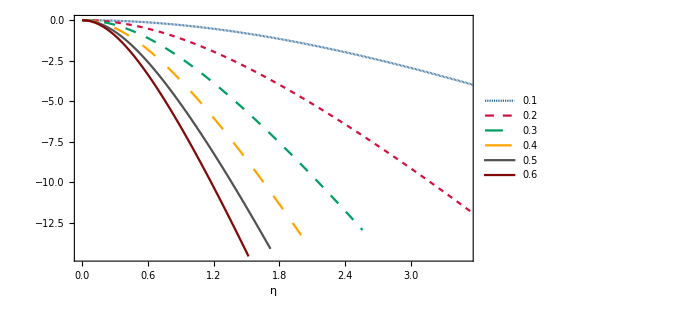

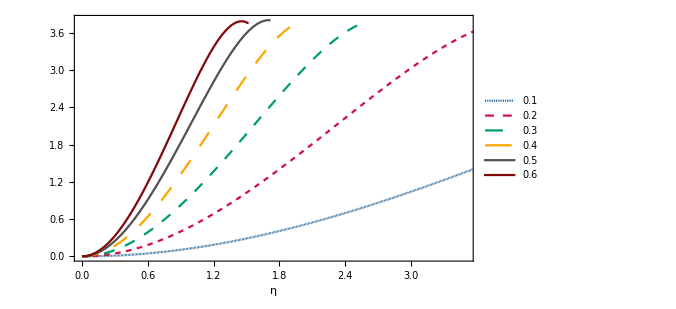

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.12,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
Max[Abs[(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100],Abs[(Max[Re[Tda[[2]]]]-Min[Re[Tda[[2]]]])/Min[Re[Tda[[2]]]]*100],Abs[(Max[Re[Tda[[3]]]]-Min[Re[Tda[[3]]]])/Min[Re[Tda[[3]]]]*100],Abs[(Max[Re[Tda[[4]]]]-Min[Re[Tda[[4]]]])/Min[Re[Tda[[4]]]]*100],Abs[(Max[Re[Tda[[5]]]]-Min[Re[Tda[[5]]]])/Min[Re[Tda[[5]]]]*100],Abs[(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100]]
Max[Abs[(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100],Abs[(Max[Im[Tda[[2]]]]-Min[Im[Tda[[2]]]])/Min[Im[Tda[[2]]]]*100],Abs[(Max[Im[Tda[[3]]]]-Min[Im[Tda[[3]]]])/Min[Im[Tda[[3]]]]*100],Abs[(Max[Im[Tda[[4]]]]-Min[Im[Tda[[4]]]])/Min[Im[Tda[[4]]]]*100],Abs[(Max[Im[Tda[[5]]]]-Min[Im[Tda[[5]]]])/Min[Im[Tda[[5]]]]*100],Abs[(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100]]
```

0.277129

0.541003

```mathematica
Max[Abs[(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100],Abs[(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100],Abs[(Max[Re[Tdp[[3]]]]-Min[Re[Tdp[[3]]]])/Min[Re[Tdp[[3]]]]*100],Abs[(Max[Re[Tdp[[4]]]]-Min[Re[Tdp[[4]]]])/Min[Re[Tdp[[4]]]]*100],Abs[(Max[Re[Tdp[[5]]]]-Min[Re[Tdp[[5]]]])/Min[Re[Tdp[[5]]]]*100],Abs[(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100],Abs[(Max[Im[Tdp[[2]]]]-Min[Im[Tdp[[2]]]])/Min[Im[Tdp[[2]]]]*100],Abs[(Max[Im[Tdp[[3]]]]-Min[Im[Tdp[[3]]]])/Min[Im[Tdp[[3]]]]*100],Abs[(Max[Im[Tdp[[4]]]]-Min[Im[Tdp[[4]]]])/Min[Im[Tdp[[4]]]]*100],Abs[(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100],Abs[(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100]]
```

16.7282

4.27226

## Scalar modes

### L=1

#### Coupled Eqs

```mathematica
T1={{{0,0.2934301134681371-0.09771120138843893 ⅈ},{1/25+ⅈ/25,0.29343169713909373-0.09771136409896833 ⅈ},{2/25+(2 ⅈ)/25,0.2934364476047949-0.09771185216837978 ⅈ},{3/25+(3 ⅈ)/25,0.29344436320904826-0.09771266540864466 ⅈ},{4/25+(4 ⅈ)/25,0.29345544119800804-0.09771380350708316 ⅈ},{1/5+ⅈ/5,0.2934696777243245-0.09771526602684465 ⅈ},{6/25+(6 ⅈ)/25,0.2934870678551328-0.09771705240780348 ⅈ},{7/25+(7 ⅈ)/25,0.29350760558225425-0.0977191619677094 ⅈ},{8/25+(8 ⅈ)/25,0.29353128383459387-0.097721593903553 ⅈ},{9/25+(9 ⅈ)/25,0.29355809449260434-0.09772434729322045 ⅈ},{2/5+(2 ⅈ)/5,0.29358802840483766-0.09772742109732704 ⅈ},{11/25+(11 ⅈ)/25,0.2936210754064495-0.09773081416129466 ⅈ},{12/25+(12 ⅈ)/25,0.2936572243395929-0.09773452521763525 ⅈ},{13/25+(13 ⅈ)/25,0.29369646307560904-0.09773855288843439 ⅈ},{14/25+(14 ⅈ)/25,0.29373877853891545-0.09774289568802358 ⅈ},{3/5+(3 ⅈ)/5,0.29378415673248864-0.09774755202582974 ⅈ},{16/25+(16 ⅈ)/25,0.2938325827648322-0.0977525202093889 ⅈ},{17/25+(17 ⅈ)/25,0.293884040878316-0.09775779844751144 ⅈ},{18/25+(18 ⅈ)/25,0.2939385144787703-0.09776338485358516 ⅈ},{19/25+(19 ⅈ)/25,0.29399598616621425-0.09776927744900295 ⅈ},{4/5+(4 ⅈ)/5,0.2940564377665976-0.09777547416670022 ⅈ},{21/25+(21 ⅈ)/25,0.29411985036443195-0.09778197285478929 ⅈ},{22/25+(22 ⅈ)/25,0.2941862043361883-0.09778877128027513 ⅈ},{23/25+(23 ⅈ)/25,0.2942554793843389-0.09779586713283987 ⅈ},{24/25+(24 ⅈ)/25,0.2943276545719203-0.09780325802868094 ⅈ},{1+ⅈ,0.29440270835749877-0.09781094151438999 ⅈ},{26/25+(26 ⅈ)/25,0.29448061863041985-0.09781891507085884 ⅈ},{27/25+(27 ⅈ)/25,0.29456136274622735-0.09782717611719925 ⅈ},{28/25+(28 ⅈ)/25,0.2946449175621427-0.09783572201466431 ⅈ},{29/25+(29 ⅈ)/25,0.29473125947249534-0.0978445500705589 ⅈ},{6/5+(6 ⅈ)/5,0.2948203644440037-0.09785365754212796 ⅈ},{31/25+(31 ⅈ)/25,0.29491220805080925-0.09786304164041101 ⅈ},{32/25+(32 ⅈ)/25,0.2950067655091704-0.09787269953405314 ⅈ},{33/25+(33 ⅈ)/25,0.2951040117117305-0.0978826283530621 ⅈ},{34/25+(34 ⅈ)/25,0.2952039212612795-0.09789282519250261 ⅈ},{7/5+(7 ⅈ)/5,0.2953064685039319-0.09790328711611916 ⅈ},{36/25+(36 ⅈ)/25,0.2954116275616544-0.09791401115988022 ⅈ},{37/25+(37 ⅈ)/25,0.2955193723640782-0.09792499433543547 ⅈ},{38/25+(38 ⅈ)/25,0.29562967667953927-0.09793623363348107 ⅈ},{39/25+(39 ⅈ)/25,0.29574251414529507-0.09794772602702614 ⅈ},{8/5+(8 ⅈ)/5,0.29585785829687267-0.09795946847455624 ⅈ},{41/25+(41 ⅈ)/25,0.2959756825965082-0.09797145792308855 ⅈ},{42/25+(42 ⅈ)/25,0.2960959604606435-0.0979836913111161 ⅈ},{43/25+(43 ⅈ)/25,0.29621866528645174-0.0979961655714371 ⅈ},{44/25+(44 ⅈ)/25,0.29634377047736793-0.09800887763386694 ⅈ},{9/5+(9 ⅈ)/5,0.2964712494676068-0.09802182442783172 ⅈ},{46/25+(46 ⅈ)/25,0.296601075745654-0.09803500288484078 ⅈ},{47/25+(47 ⅈ)/25,0.29673322287672127-0.09804840994083824 ⅈ},{48/25+(48 ⅈ)/25,0.29686766452416186-0.09806204253843293 ⅈ},{49/25+(49 ⅈ)/25,0.29700437446984423-0.09807589762900652 ⅈ},{2+2 ⅈ,0.2971433266334879-0.09808997217470097 ⅈ},{51/25+(51 ⅈ)/25,0.2972844950909678-0.09810426315028542 ⅈ},{52/25+(52 ⅈ)/25,0.2974278540915964-0.09811876754490483 ⅈ},{53/25+(53 ⅈ)/25,0.2975733780743967-0.09813348236371078 ⅈ},{54/25+(54 ⅈ)/25,0.29772104168338104-0.09814840462937739 ⅈ},{11/5+(11 ⅈ)/5,0.29787081978185315-0.09816353138350398 ⅈ},{56/25+(56 ⅈ)/25,0.29802268746575383-0.09817885968790706 ⅈ},{57/25+(57 ⅈ)/25,0.29817662007607143-0.0981943866258041 ⅈ},{58/25+(58 ⅈ)/25,0.2983325932103401-0.0982101093028924 ⅈ},{59/25+(59 ⅈ)/25,0.2984905827332515-0.09822602484832527 ⅈ},{12/5+(12 ⅈ)/5,0.2986505647864048-0.09824213041558946 ⅈ},{61/25+(61 ⅈ)/25,0.29881251579722234-0.09825842318328648 ⅈ},{62/25+(62 ⅈ)/25,0.29897641248705925-0.09827490035582125 ⅈ},{63/25+(63 ⅈ)/25,0.29914223187853395-0.09829155916400174 ⅈ},{64/25+(64 ⅈ)/25,0.2993099513021096-0.09830839686555261 ⅈ},{13/5+(13 ⅈ)/5,0.29947954840195495-0.09832541074554663 ⅈ},{66/25+(66 ⅈ)/25,0.2996510011411142-0.09834259811675729 ⅈ},{67/25+(67 ⅈ)/25,0.29982428780601467-0.0983599563199359 ⅈ},{68/25+(68 ⅈ)/25,0.29999938701034207-0.09837748272401683 ⅈ},{69/25+(69 ⅈ)/25,0.30017627769831157-0.09839517472625449 ⅈ},{14/5+(14 ⅈ)/5,0.3003549391473643-0.09841302975229464 ⅈ},{71/25+(71 ⅈ)/25,0.3005353509703169-0.09843104525618482 ⅈ},{72/25+(72 ⅈ)/25,0.3007174931169919-0.09844921872032553 ⅈ},{73/25+(73 ⅈ)/25,0.300901345875357-0.09846754765536676 ⅈ},{74/25+(74 ⅈ)/25,0.30108688987219867-0.09848602960005219 ⅈ},{3+3 ⅈ,0.3012741060733581-0.09850466212101452 ⅈ},{76/25+(76 ⅈ)/25,0.30146297578355213-0.09852344281252491 ⅈ},{77/25+(77 ⅈ)/25,0.30165348064580694-0.09854236929619929 ⅈ},{78/25+(78 ⅈ)/25,0.3018456026405254-0.09856143922066452 ⅈ},{79/25+(79 ⅈ)/25,0.302039324084214-0.09858065026118693 ⅈ},{16/5+(16 ⅈ)/5,0.30223462762788944-0.09860000011926644 ⅈ},{81/25+(81 ⅈ)/25,0.30243149625518767-0.09861948652219785 ⅈ},{82/25+(82 ⅈ)/25,0.30262991328019584-0.09863910722260287 ⅈ},{83/25+(83 ⅈ)/25,0.3028298623450269-0.09865885999793442 ⅈ},{84/25+(84 ⅈ)/25,0.30303132741715616-0.09867874264995578 ⅈ},{17/5+(17 ⅈ)/5,0.3032342927865381-0.09869875300419678 ⅈ},{86/25+(86 ⅈ)/25,0.30343874306252033-0.09871888890938922 ⅈ},{87/25+(87 ⅈ)/25,0.3036446631705731-0.0987391482368832 ⅈ},{88/25+(88 ⅈ)/25,0.3038520383488473-0.09875952888004648 ⅈ},{89/25+(89 ⅈ)/25,0.30406085414457984-0.09878002875364886 ⅈ},{18/5+(18 ⅈ)/5,0.3042710964103574-0.0988006457932327 ⅈ},{91/25+(91 ⅈ)/25,0.30448275130025426-0.09882137795447202 ⅈ},{92/25+(92 ⅈ)/25,0.3046958052658569-0.0988422232125212 ⅈ},{93/25+(93 ⅈ)/25,0.3049102450521866-0.09886317956135486 ⅈ},{94/25+(94 ⅈ)/25,0.30512605769353324-0.09888424501310046 ⅈ},{19/5+(19 ⅈ)/5,0.30534323050920964-0.09890541759736485 ⅈ},{96/25+(96 ⅈ)/25,0.305561751099238-0.09892669536055612 ⅈ},{97/25+(97 ⅈ)/25,0.30578160733997783-0.09894807636520174 ⅈ},{98/25+(98 ⅈ)/25,0.3060027873797036-0.09896955868926446 ⅈ},{99/25+(99 ⅈ)/25,0.3062252796341423-0.09899114042545666 ⅈ},{4+4 ⅈ,0.3064490727819775-0.09901281968055443 ⅈ},{101/25+(101 ⅈ)/25,0.30667415576032864-0.09903459457471216 ⅈ},{102/25+(102 ⅈ)/25,0.30690051776021093-0.09905646324077858 ⅈ},{103/25+(103 ⅈ)/25,0.3071281482219848-0.09907842382361523 ⅈ},{104/25+(104 ⅈ)/25,0.3073570368307986-0.0991004744794177 ⅈ},{21/5+(21 ⅈ)/5,0.307587173512032-0.09912261337504105 ⅈ},{106/25+(106 ⅈ)/25,0.30781854842674383-0.09914483868732944 ⅈ},{107/25+(107 ⅈ)/25,0.30805115196713123-0.09916714860245093 ⅈ},{108/25+(108 ⅈ)/25,0.3082849747520024-0.0991895413152382 ⅈ},{109/25+(109 ⅈ)/25,0.3085200076222691-0.09921201502853541 ⅈ},{22/5+(22 ⅈ)/5,0.308756241636461-0.0992345679525519 ⅈ},{111/25+(111 ⅈ)/25,0.3089936680662667-0.09925719830422326 ⅈ},{112/25+(112 ⅈ)/25,0.30923227839210454-0.09927990430658014 ⅈ},{113/25+(113 ⅈ)/25,0.30947206429872487-0.09930268418812534 ⅈ},{114/25+(114 ⅈ)/25,0.3097130176708482-0.09932553618221929 ⅈ},{23/5+(23 ⅈ)/5,0.3099551305888404-0.09934845852647477 ⅈ},{116/25+(116 ⅈ)/25,0.3101983953244278-0.0993714494621607 ⅈ},{117/25+(117 ⅈ)/25,0.3104428043364542-0.0993945072336157 ⅈ},{118/25+(118 ⅈ)/25,0.31068835026668057-0.09941763008767147 ⅈ},{119/25+(119 ⅈ)/25,0.3109350259356306-0.09944081627308644 ⅈ},{24/5+(24 ⅈ)/5,0.3111828243384824-0.09946406403998975 ⅈ},{121/25+(121 ⅈ)/25,0.3114317386410077-0.09948737163933594 ⅈ},{122/25+(122 ⅈ)/25,0.31168176217556004-0.09951073732237066 ⅈ},{123/25+(123 ⅈ)/25,0.31193288843711225-0.09953415934010713 ⅈ},{124/25+(124 ⅈ)/25,0.31218511107934493-0.09955763594281423 ⅈ},{5+5 ⅈ,0.3124384239107856-0.09958116537951577 ⅈ},{126/25+(126 ⅈ)/25,0.3126928208909993-0.09960474589750133 ⅈ},{127/25+(127 ⅈ)/25,0.31294829612683206-0.099628375741849 ⅈ},{128/25+(128 ⅈ)/25,0.31320484386870573-0.09965205315495979 ⅈ},{129/25+(129 ⅈ)/25,0.31346245850696597-0.09967577637610403 ⅈ},{26/5+(26 ⅈ)/5,0.31372113456828316-0.09969954364097991 ⅈ},{131/25+(131 ⅈ)/25,0.31398086671210534-0.09972335318128414 ⅈ},{132/25+(132 ⅈ)/25,0.3142416497271652-0.09974720322429473 ⅈ},{133/25+(133 ⅈ)/25,0.31450347852803795-0.09977109199246632 ⅈ},{134/25+(134 ⅈ)/25,0.3147663481517536-0.09979501770303782 ⅈ},{27/5+(27 ⅈ)/5,0.3150302537544603-0.09981897856765237 ⅈ},{136/25+(136 ⅈ)/25,0.3152951906081405-0.09984297279199006 ⅈ},{137/25+(137 ⅈ)/25,0.3155611540973782-0.09986699857541297 ⅈ},{138/25+(138 ⅈ)/25,0.31582813971617857-0.09989105411062306 ⅈ},{139/25+(139 ⅈ)/25,0.31609614306483746-0.09991513758333263 ⅈ},{28/5+(28 ⅈ)/5,0.3163651598468626-0.09993924717194724 ⅈ},{141/25+(141 ⅈ)/25,0.3166351858659442-0.0999633810472618 ⅈ},{142/25+(142 ⅈ)/25,0.31690621702297594-0.09998753737216899 ⅈ},{143/25+(143 ⅈ)/25,0.3171782493131245-0.10001171430138062 ⅈ},{144/25+(144 ⅈ)/25,0.3174512788229482-0.10003590998116184 ⅈ},{29/5+(29 ⅈ)/5,0.3177253017275637-0.1000601225490779 ⅈ},{146/25+(146 ⅈ)/25,0.3180003142878599-0.10008435013375411 ⅈ},{147/25+(147 ⅈ)/25,0.3182763128477597-0.10010859085464806 ⅈ},{148/25+(148 ⅈ)/25,0.31855329383152725-0.10013284282183527 ⅈ},{149/25+(149 ⅈ)/25,0.3188312537411218-0.10015710413580707 ⅈ},{6+6 ⅈ,0.3191101891535962-0.1001813728872818 ⅈ},{151/25+(151 ⅈ)/25,0.3193900967185407-0.10020564715702841 ⅈ},{152/25+(152 ⅈ)/25,0.31967097315557-0.10022992501570308 ⅈ},{153/25+(153 ⅈ)/25,0.3199528152518548-0.10025420452369857 ⅈ},{154/25+(154 ⅈ)/25,0.3202356198596951-0.10027848373100628 ⅈ},{31/5+(31 ⅈ)/5,0.32051938389413664-0.10030276067709123 ⅈ},{156/25+(156 ⅈ)/25,0.3208041043306281-0.10032703339077961 ⅈ},{157/25+(157 ⅈ)/25,0.32108977820272083-0.10035129989015902 ⅈ},{158/25+(158 ⅈ)/25,0.321376402599807-0.10037555818249155 ⅈ},{159/25+(159 ⅈ)/25,0.3216639746648995-0.10039980626413952 ⅈ},{32/5+(32 ⅈ)/5,0.32195249159245004-0.10042404212050367 ⅈ},{161/25+(161 ⅈ)/25,0.3222419506262064-0.10044826372597408 ⅈ},{162/25+(162 ⅈ)/25,0.3225323490571079-0.10047246904389372 ⅈ},{163/25+(163 ⅈ)/25,0.32282368422121804-0.10049665602653436 ⅈ},{164/25+(164 ⅈ)/25,0.32311595349769473-0.10052082261508516 ⅈ},{33/5+(33 ⅈ)/5,0.32340915430679673-0.10054496673965355 ⅈ},{166/25+(166 ⅈ)/25,0.32370328410792626-0.10056908631927863 ⅈ},{167/25+(167 ⅈ)/25,0.32399834039770714-0.10059317926195681 ⅈ},{168/25+(168 ⅈ)/25,0.32429432070809755-0.10061724346467996 ⅈ},{169/25+(169 ⅈ)/25,0.32459122260453765-0.10064127681348548 ⅈ},{34/5+(34 ⅈ)/5,0.32488904368413113-0.10066527718351895 ⅈ},{171/25+(171 ⅈ)/25,0.3251877815738601-0.10068924243910864 ⅈ},{172/25+(172 ⅈ)/25,0.3254874339288332-0.10071317043385208 ⅈ},{173/25+(173 ⅈ)/25,0.3257879984305665-0.10073705901071502 ⅈ},{174/25+(174 ⅈ)/25,0.326089472785296-0.10076090600214165 ⅈ},{7+7 ⅈ,0.32639185472232246-0.1007847092301774 ⅈ},{176/25+(176 ⅈ)/25,0.32669514199238747-0.10080846650660308 ⅈ},{177/25+(177 ⅈ)/25,0.32699933236607986-0.1008321756330808 ⅈ},{178/25+(178 ⅈ)/25,0.32730442363227374-0.10085583440131156 ⅈ}},{{0,0.29490584811772586-0.09786585160959349 ⅈ},{1/25+ⅈ/25,0.29491219900450055-0.09786649202768732 ⅈ},{2/25+(2 ⅈ)/25,0.2949312426284681-0.09786841227206068 ⅈ},{3/25+(3 ⅈ)/25,0.2949629518941012-0.09787160931505241 ⅈ},{4/25+(4 ⅈ)/25,0.29500728190800235-0.09787607813989795 ⅈ},{1/5+ⅈ/5,0.2950641703503-0.09788181178185781 ⅈ},{6/25+(6 ⅈ)/25,0.2951335379933918-0.09788880138558463 ⅈ},{7/25+(7 ⅈ)/25,0.29521528935202446-0.09789703627696546 ⅈ},{8/25+(8 ⅈ)/25,0.2953093134528352-0.0979065040481005 ⅈ},{9/25+(9 ⅈ)/25,0.2954154847096546-0.09791719065386921 ⅈ},{2/5+(2 ⅈ)/5,0.29553366388947694-0.09792908051837845 ⅈ},{11/25+(11 ⅈ)/25,0.29566369915305174-0.09794215664948014 ⅈ},{12/25+(12 ⅈ)/25,0.2958054271535533-0.0979564007594922 ⅈ},{13/25+(13 ⅈ)/25,0.2959586741767196-0.09797179339025028 ⅈ},{14/25+(14 ⅈ)/25,0.2961232573061957-0.0979883140406585 ⅈ},{3/5+(3 ⅈ)/5,0.29629898559851514-0.09800594129498968 ⅈ},{16/25+(16 ⅈ)/25,0.29648566125316517-0.09802465295029991 ⅈ},{17/25+(17 ⅈ)/25,0.29668308076443006-0.0980444261414676 ⅈ},{18/25+(18 ⅈ)/25,0.2968910360431459-0.09806523746253092 ⅈ},{19/25+(19 ⅈ)/25,0.2971093154980569-0.098087063083174 ⅈ},{4/5+(4 ⅈ)/5,0.29733770506808-0.09810987885939958 ⅈ},{21/25+(21 ⅈ)/25,0.297575989198414-0.09813366043760763 ⅈ},{22/25+(22 ⅈ)/25,0.29782395175501875-0.09815838335148251 ⅈ},{23/25+(23 ⅈ)/25,0.29808137687350156-0.09818402311126227 ⅈ},{24/25+(24 ⅈ)/25,0.29834804973985934-0.09821055528512249 ⅈ},{1+ⅈ,0.2986237573018011-0.09823795557255308 ⅈ},{26/25+(26 ⅈ)/25,0.29890828891051485-0.09826619986973319 ⅈ},{27/25+(27 ⅈ)/25,0.29920143689373063-0.09829526432702566 ⅈ},{28/25+(28 ⅈ)/25,0.29950299706176553-0.09832512539879106 ⅈ},{29/25+(29 ⅈ)/25,0.2998127691489292-0.09835575988582877 ⅈ},{6/5+(6 ⅈ)/5,0.3001305571932107-0.09838714497077589 ⅈ},{31/25+(31 ⅈ)/25,0.3004561698575899-0.0984192582468714 ⅈ},{32/25+(32 ⅈ)/25,0.3007894206966093-0.0984520777405104 ⅈ},{33/25+(33 ⅈ)/25,0.30113012837204134-0.09848558192803897 ⅈ},{34/25+(34 ⅈ)/25,0.3014781168215798-0.0985197497472492 ⅈ},{7/5+(7 ⅈ)/5,0.3018332153845122-0.09855456060403696 ⅈ},{36/25+(36 ⅈ)/25,0.30219525888828147-0.09858999437467762 ⅈ},{37/25+(37 ⅈ)/25,0.30256408769975396-0.09862603140416491 ⅈ},{38/25+(38 ⅈ)/25,0.3029395477448662-0.09866265250104016 ⅈ},{39/25+(39 ⅈ)/25,0.3033214905001569-0.09869983892912079 ⅈ},{8/5+(8 ⅈ)/5,0.3037097729594935-0.09873757239651279 ⅈ},{41/25+(41 ⅈ)/25,0.3041042575790952-0.09877583504226944 ⅈ},{42/25+(42 ⅈ)/25,0.30450481220373443-0.09881460942103226 ⅈ},{43/25+(43 ⅈ)/25,0.3049113099767767-0.09885387848596532 ⅈ},{44/25+(44 ⅈ)/25,0.30532362923649986-0.09889362557026843 ⅈ},{9/5+(9 ⅈ)/5,0.30574165340091297-0.09893383436753075 ⅈ},{46/25+(46 ⅈ)/25,0.3061652708430901-0.09897448891116166 ⅈ},{47/25+(47 ⅈ)/25,0.30659437475882917-0.09901557355311347 ⅈ},{48/25+(48 ⅈ)/25,0.30702886302826166-0.09905707294208964 ⅈ},{49/25+(49 ⅈ)/25,0.30746863807285496-0.09909897200141045 ⅈ},{2+2 ⅈ,0.30791360670908885-0.09914125590669169 ⅈ},{51/25+(51 ⅈ)/25,0.30836367999993053-0.09918391006347246 ⅈ},{52/25+(52 ⅈ)/25,0.30881877310509326-0.09922692008491386 ⅈ},{53/25+(53 ⅈ)/25,0.3092788051309344-0.09927027176967507 ⅈ},{54/25+(54 ⅈ)/25,0.30974369898073184-0.09931395108006111 ⅈ},{11/5+(11 ⅈ)/5,0.3102133812059702-0.09935794412052328 ⅈ},{56/25+(56 ⅈ)/25,0.31068778185917645-0.09940223711658445 ⅈ},{57/25+(57 ⅈ)/25,0.311166834348755-0.09944681639425057 ⅈ},{58/25+(58 ⅈ)/25,0.31165047529619816-0.09949166835996173 ⅈ},{59/25+(59 ⅈ)/25,0.3121386443959822-0.09953677948112857 ⅈ},{12/5+(12 ⅈ)/5,0.312631284278394-0.09958213626729355 ⅈ},{61/25+(61 ⅈ)/25,0.3131283403754869-0.09962772525195002 ⅈ},{62/25+(62 ⅈ)/25,0.31362976079031496-0.09967353297504776 ⅈ},{63/25+(63 ⅈ)/25,0.3141354961695538-0.09971954596620869 ⅈ},{64/25+(64 ⅈ)/25,0.31464549957958554-0.09976575072867228 ⅈ},{13/5+(13 ⅈ)/5,0.31515972638609097-0.09981213372398814 ⅈ},{66/25+(66 ⅈ)/25,0.3156781341371692-0.09985868135746848 ⅈ},{67/25+(67 ⅈ)/25,0.3162006824499836-0.09990537996441254 ⅈ},{68/25+(68 ⅈ)/25,0.31672733290091193-0.09995221579711101 ⅈ},{69/25+(69 ⅈ)/25,0.31725804891916626-0.09999917501263896 ⅈ},{14/5+(14 ⅈ)/5,0.3177927956838345-0.10004624366144144 ⅈ},{71/25+(71 ⅈ)/25,0.31833154002428454-0.10009340767671718 ⅈ},{72/25+(72 ⅈ)/25,0.3188742503238652-0.10014065286460298 ⅈ},{73/25+(73 ⅈ)/25,0.3194208964268311-0.10018796489516085 ⅈ},{74/25+(74 ⅈ)/25,0.31997144954841433-0.10023532929416938 ⅈ},{3+3 ⅈ,0.32052588218796163-0.10028273143571972 ⅈ},{76/25+(76 ⅈ)/25,0.3210841680450549-0.10033015653561564 ⅈ},{77/25+(77 ⅈ)/25,0.32164628193853123-0.1003775896455777 ⅈ},{78/25+(78 ⅈ)/25,0.32221219972831766-0.10042501564824893 ⅈ},{79/25+(79 ⅈ)/25,0.32278189823999703-0.10047241925300103 ⅈ},{16/5+(16 ⅈ)/5,0.32335535519202363-0.10051978499253834 ⅈ},{81/25+(81 ⅈ)/25,0.3239325491255055-0.10056709722029629 ⅈ},{82/25+(82 ⅈ)/25,0.32451345933647685-0.10061434010863111 ⅈ},{83/25+(83 ⅈ)/25,0.3250980658105819-0.10066149764779685 ⅈ},{84/25+(84 ⅈ)/25,0.3256863491600984-0.10070855364570433 ⅈ},{17/5+(17 ⅈ)/5,0.32627829056322755-0.10075549172845802 ⅈ},{86/25+(86 ⅈ)/25,0.32687387170558446-0.10080229534166345 ⅈ},{87/25+(87 ⅈ)/25,0.32747307472382287-0.10084894775249993 ⅈ},{88/25+(88 ⅈ)/25,0.32807588215133304-0.1008954320525505 ⅈ},{89/25+(89 ⅈ)/25,0.32868227686595397-0.10094173116138144 ⅈ},{18/5+(18 ⅈ)/5,0.32929224203964486-0.10098782783086216 ⅈ},{91/25+(91 ⅈ)/25,0.32990576109006386-0.10103370465021622 ⅈ}},{{0,0.29734494056573973-0.09812674596109573 ⅈ},{1/25+ⅈ/25,0.29735929784812914-0.09812814977365117 ⅈ},{2/25+(2 ⅈ)/25,0.2974023218855444-0.09813235600258753 ⅈ},{3/25+(3 ⅈ)/25,0.2974738700498331-0.09813934911006285 ⅈ},{4/25+(4 ⅈ)/25,0.29757370775841435-0.09814910353858253 ⅈ},{1/5+ⅈ/5,0.29770151297674835-0.09816158419856044 ⅈ},{6/25+(6 ⅈ)/25,0.29785688226588203-0.098176747122357 ⅈ},{7/25+(7 ⅈ)/25,0.29803933811016897-0.0981945402557148 ⅈ},{8/25+(8 ⅈ)/25,0.2982483372360469-0.09821490435467384 ⅈ},{9/25+(9 ⅈ)/25,0.2984832796136153-0.09823777395396598 ⅈ},{2/5+(2 ⅈ)/5,0.29874351783253933-0.09826307837290545 ⅈ},{11/25+(11 ⅈ)/25,0.29902836656037246-0.09829074272666875 ⅈ},{12/25+(12 ⅈ)/25,0.29933711182138706-0.09832068891421838 ⅈ},{13/25+(13 ⅈ)/25,0.2996690198734464-0.09835283655852878 ⅈ},{14/25+(14 ⅈ)/25,0.30002334550524684-0.09838710387975928 ⅈ},{3/5+(3 ⅈ)/5,0.30039933962259424-0.09842340848717118 ⅈ},{16/25+(16 ⅈ)/25,0.300796256037107-0.09846166808054722 ⅈ},{17/25+(17 ⅈ)/25,0.30121335741145616-0.09850180105638345 ⅈ},{18/25+(18 ⅈ)/25,0.30164992035040517-0.09854372701800863 ⅈ},{19/25+(19 ⅈ)/25,0.3021052396556886-0.09858736719196079 ⅈ},{4/5+(4 ⅈ)/5,0.30257863178500294-0.09863264475539434 ⅈ},{21/25+(21 ⅈ)/25,0.30306943757138055-0.09867948508104321 ⅈ},{22/25+(22 ⅈ)/25,0.30357702426962535-0.0987278159073952 ⅈ},{23/25+(23 ⅈ)/25,0.3041007870021196-0.09877756744233458 ⅈ},{24/25+(24 ⅈ)/25,0.3046401496780674-0.09882867240868397 ⅈ},{1+ⅈ,0.30519456545899853-0.09888106603991949 ⅈ},{26/25+(26 ⅈ)/25,0.30576351683992237-0.09893468603393664 ⅈ},{27/25+(27 ⅈ)/25,0.3063465154106023-0.0989894724721834 ⅈ},{28/25+(28 ⅈ)/25,0.3069431013555997-0.0990453677108303 ⅈ},{29/25+(29 ⅈ)/25,0.3075528427454783-0.09910231624992695 ⅈ},{6/5+(6 ⅈ)/5,0.3081753346652187-0.09916026458580993 ⅈ},{31/25+(31 ⅈ)/25,0.30881019821972944-0.09921916105132242 ⅈ},{32/25+(32 ⅈ)/25,0.3094570794505263-0.09927895564776985 ⅈ},{33/25+(33 ⅈ)/25,0.31011564819230103-0.09933959987194035 ⅈ},{34/25+(34 ⅈ)/25,0.31078559689326896-0.09940104654098664 ⅈ},{7/5+(7 ⅈ)/5,0.31146663941889535-0.09946324961749359 ⅈ},{36/25+(36 ⅈ)/25,0.31215850985484545-0.09952616403664298 ⅈ},{37/25+(37 ⅈ)/25,0.312860961321758-0.09958974553703275 ⅈ},{38/25+(38 ⅈ)/25,0.3135737648116692-0.09965395049640546 ⅈ},{39/25+(39 ⅈ)/25,0.3142967080535734-0.0997187357732856 ⅈ},{8/5+(8 ⅈ)/5,0.31502959441364514-0.09978405855531357 ⅈ},{41/25+(41 ⅈ)/25,0.31577224183403135-0.09984987621488906 ⅈ},{42/25+(42 ⅈ)/25,0.3165244818127929-0.0999161461725935 ⅈ},{43/25+(43 ⅈ)/25,0.317286158426505-0.09998282576874568 ⅈ},{44/25+(44 ⅈ)/25,0.31805712739616837-0.10004987214335222 ⅈ},{9/5+(9 ⅈ)/5,0.3188372551964123-0.10011724212464151 ⅈ},{46/25+(46 ⅈ)/25,0.31962641820744825-0.10018489212631268 ⅈ},{47/25+(47 ⅈ)/25,0.32042450190884353-0.10025277805358622 ⅈ},{48/25+(48 ⅈ)/25,0.32123140011389667-0.10032085521810985 ⅈ},{49/25+(49 ⅈ)/25,0.3220470142431965-0.1003890782617461 ⅈ},{2+2 ⅈ,0.32287125263581645-0.10045740108924965 ⅈ},{51/25+(51 ⅈ)/25,0.32370402989652464-0.10052577680982618 ⅈ},{52/25+(52 ⅈ)/25,0.3245452662773571-0.10059415768755342 ⅈ},{53/25+(53 ⅈ)/25,0.3253948870919135-0.10066249510063437 ⅈ},{54/25+(54 ⅈ)/25,0.32625282216076534-0.10073073950944489 ⅈ},{11/5+(11 ⅈ)/5,0.32711900528642185-0.10079884043332847 ⅈ},{56/25+(56 ⅈ)/25,0.3279933737563704-0.10086674643608326 ⅈ},{57/25+(57 ⅈ)/25,0.32887586787278594-0.10093440512007558 ⅈ},{58/25+(58 ⅈ)/25,0.32976643050759485-0.1010017631289053 ⅈ},{59/25+(59 ⅈ)/25,0.3306650066816675-0.10106876615853388 ⅈ},{12/5+(12 ⅈ)/5,0.3315715431670091-0.10113535897677436 ⅈ},{61/25+(61 ⅈ)/25,0.3324859881109104-0.1012014854510242 ⅈ},{62/25+(62 ⅈ)/25,0.3334082906811114-0.10126708858410645 ⅈ},{63/25+(63 ⅈ)/25,0.3343384007311194-0.10133211055806286 ⅈ},{64/25+(64 ⅈ)/25,0.33527626848490716-0.10139649278572198 ⅈ}},{{0,0.30071745721129695-0.09849783114098085 ⅈ},{1/25+ⅈ/25,0.3007431768142335-0.09850024163397418 ⅈ},{2/25+(2 ⅈ)/25,0.3008201747381251-0.09850745615434196 ⅈ},{3/25+(3 ⅈ)/25,0.3009479739781611-0.09851942442480774 ⅈ},{4/25+(4 ⅈ)/25,0.30112579877410495-0.09853606467738138 ⅈ},{1/5+ⅈ/5,0.30135260176114-0.09855726651118493 ⅈ},{6/25+(6 ⅈ)/25,0.3016270989931223-0.0985828945724999 ⅈ},{7/25+(7 ⅈ)/25,0.30194781029049117-0.09861279278439561 ⅈ},{8/25+(8 ⅈ)/25,0.3023131022687132-0.09864678884293436 ⅈ},{9/25+(9 ⅈ)/25,0.30272123156009245-0.0986846987141775 ⅈ},{2/5+(2 ⅈ)/5,0.30317038611120345-0.09872633090625724 ⅈ},{11/25+(11 ⅈ)/25,0.30365872293419366-0.09877149034435627 ⅈ},{12/25+(12 ⅈ)/25,0.30418440122764345-0.09881998173438179 ⅈ},{13/25+(13 ⅈ)/25,0.30474561029189134-0.09887161235592848 ⅈ},{14/25+(14 ⅈ)/25,0.30534059209774417-0.09892619427175403 ⅈ},{3/5+(3 ⅈ)/5,0.30596765870266307-0.09898354597691754 ⅈ},{16/25+(16 ⅈ)/25,0.3066252049406153-0.09904349353551994 ⅈ},{17/25+(17 ⅈ)/25,0.307311716950059-0.09910587126766228 ⅈ},{18/25+(18 ⅈ)/25,0.30802577716569063-0.09917052205561365 ⅈ},{19/25+(19 ⅈ)/25,0.3087660664028806-0.09923729733834671 ⅈ},{4/5+(4 ⅈ)/5,0.3095313636275728-0.09930605685954702 ⅈ},{21/25+(21 ⅈ)/25,0.3103205439445363-0.0993766682276274 ⅈ},{22/25+(22 ⅈ)/25,0.3111325752654642-0.09944900633849961 ⅈ},{23/25+(23 ⅈ)/25,0.3119665140443152-0.09952295270381732 ⅈ},{24/25+(24 ⅈ)/25,0.31282150039629525-0.09959839471973116 ⅈ},{1+ⅈ,0.31369675285238763-0.09967522490424538 ⅈ},{26/25+(26 ⅈ)/25,0.3145915629450364-0.09975334012522188 ⅈ},{27/25+(27 ⅈ)/25,0.3155052897729228-0.09983264083596359 ⅈ},{28/25+(28 ⅈ)/25,0.316437354653431-0.09991303033115435 ⅈ},{29/25+(29 ⅈ)/25,0.3173872359396703-0.09999441403248546 ⅈ},{6/5+(6 ⅈ)/5,0.3183544640537946-0.10007669881074681 ⅈ},{31/25+(31 ⅈ)/25,0.3193386167689067-0.10015979234903667 ⅈ},{32/25+(32 ⅈ)/25,0.32033931475703165-0.10024360255024195 ⅈ},{33/25+(33 ⅈ)/25,0.3213562174096474-0.10032803699078773 ⅈ},{34/25+(34 ⅈ)/25,0.32238901892929417-0.10041300242183557 ⅈ},{7/5+(7 ⅈ)/5,0.323437444685208-0.10049840431853431 ⅈ},{36/25+(36 ⅈ)/25,0.3245012478221938-0.10058414647753852 ⅈ},{37/25+(37 ⅈ)/25,0.32558020610963767-0.10067013066275847 ⅈ},{38/25+(38 ⅈ)/25,0.326674119016308-0.10075625629915182 ⅈ},{39/25+(39 ⅈ)/25,0.3277828049961261-0.10084242021427944 ⅈ},{8/5+(8 ⅈ)/5,0.3289060989701914-0.1009285164273028 ⅈ},{41/25+(41 ⅈ)/25,0.3300438499908466-0.10101443598507263 ⅈ},{42/25+(42 ⅈ)/25,0.331195919074345-0.10110006684494344 ⅈ},{43/25+(43 ⅈ)/25,0.3323621771896246-0.10118529380392187 ⅈ},{44/25+(44 ⅈ)/25,0.33354250339174574-0.10126999847372016 ⅈ},{9/5+(9 ⅈ)/5,0.3347367830896326-0.10135405930122783 ⅈ},{46/25+(46 ⅈ)/25,0.3359449064388549-0.10143735163383216 ⅈ},{47/25+(47 ⅈ)/25,0.33716676685125113-0.10151974782890706 ⅈ},{48/25+(48 ⅈ)/25,0.3384022596142109-0.1016011174066525 ⅈ},{49/25+(49 ⅈ)/25,0.3396512806133858-0.10168132724529799 ⅈ},{2+2 ⅈ,0.34091372515347773-0.10176024181748942 ⅈ}},{{0,0.3049829820416122-0.09898323828394866 ⅈ},{1/25+ⅈ/25,0.305023636495005-0.09898685265561466 ⅈ},{2/25+(2 ⅈ)/25,0.3051451725153767-0.09899765240747944 ⅈ},{3/25+(3 ⅈ)/25,0.3053463336829677-0.09901551007006261 ⅈ},{4/25+(4 ⅈ)/25,0.3056251092001341-0.09904022168865727 ⅈ},{1/5+ⅈ/5,0.30597884710713347-0.09907151836016619 ⅈ},{6/25+(6 ⅈ)/25,0.3064043925408542-0.09910908028533129 ⅈ},{7/25+(7 ⅈ)/25,0.30689823603268207-0.09915255178367499 ⅈ},{8/25+(8 ⅈ)/25,0.30745665826900254-0.09920155586830567 ⅈ},{9/25+(9 ⅈ)/25,0.30807586089091893-0.09925570730721534 ⅈ},{2/5+(2 ⅈ)/5,0.3087520767894539-0.09931462350206371 ⅈ},{11/25+(11 ⅈ)/25,0.30948165705955094-0.09937793290109737 ⅈ},{12/25+(12 ⅈ)/25,0.3102611347420168-0.09944528097074576 ⅈ},{13/25+(13 ⅈ)/25,0.3110872674892599-0.09951633395809825 ⅈ},{14/25+(14 ⅈ)/25,0.3119570623839356-0.0995907807888751 ⅈ},{3/5+(3 ⅈ)/5,0.3128677865088622-0.09966833348258548 ⅈ},{16/25+(16 ⅈ)/25,0.3138169667436628-0.09974872645257968 ⅈ},{17/25+(17 ⅈ)/25,0.31480238185884785-0.09983171501563151 ⅈ},{18/25+(18 ⅈ)/25,0.31582204945200115-0.0999170733802597 ⅈ},{19/25+(19 ⅈ)/25,0.31687420973004954-0.10000459232630958 ⅈ},{4/5+(4 ⅈ)/5,0.3179573076474705-0.10009407673670498 ⅈ},{21/25+(21 ⅈ)/25,0.3190699744909827-0.1001853430986434 ⅈ},{22/25+(22 ⅈ)/25,0.3202110096637927-0.10027821705653259 ⅈ},{23/25+(23 ⅈ)/25,0.3213793631619474-0.10037253107210084 ⅈ},{24/25+(24 ⅈ)/25,0.32257411904120203-0.10046812222722146 ⅈ},{1+ⅈ,0.32379448003283984-0.10056483019076994 ⅈ},{26/25+(26 ⅈ)/25,0.3250397533692981-0.10066249536102831 ⅈ},{27/25+(27 ⅈ)/25,0.3263093378150464-0.10076095718864414 ⅈ},{28/25+(28 ⅈ)/25,0.32760271185637496-0.10086005268119752 ⅈ},{29/25+(29 ⅈ)/25,0.3289194229792258-0.10095961508788824 ⅈ},{6/5+(6 ⅈ)/5,0.33025907795135806-0.10105947276194199 ⅈ},{31/25+(31 ⅈ)/25,0.33162133402078325-0.10115944819771636 ⅈ},{32/25+(32 ⅈ)/25,0.33300589094326954-0.10125935723963227 ⅈ},{33/25+(33 ⅈ)/25,0.3344124837560968-0.10135900846030095 ⅈ},{34/25+(34 ⅈ)/25,0.33584087622163983-0.10145820270556648 ⅈ},{7/5+(7 ⅈ)/5,0.337290854871819-0.10155673280449068 ⅈ},{36/25+(36 ⅈ)/25,0.3387622235923282-0.10165438344249586 ⅈ},{37/25+(37 ⅈ)/25,0.34025479869339126-0.10175093119589781 ⅈ},{38/25+(38 ⅈ)/25,0.34176840442132495-0.10184614472587507 ⅈ},{39/25+(39 ⅈ)/25,0.3433028688722289-0.10193978512951056 ⅈ},{8/5+(8 ⅈ)/5,0.3448580202755622-0.10203160644490282 ⅈ},{41/25+(41 ⅈ)/25,0.34643368362115873-0.10212135630647981 ⅈ},{42/25+(42 ⅈ)/25,0.34802967760833364-0.1022087767455709 ⅈ},{43/25+(43 ⅈ)/25,0.3496458119001519-0.10229360513002358 ⅈ}},{{0,0.31009201405974723-0.09958619259031025 ⅈ},{1/25+ⅈ/25,0.3101515544864499-0.09959117111682296 ⅈ},{2/25+(2 ⅈ)/25,0.3103291871653887-0.09960601030665815 ⅈ},{3/25+(3 ⅈ)/25,0.3106220390846032-0.0996304301752686 ⅈ},{4/25+(4 ⅈ)/25,0.3110256138599219-0.09966399292186251 ⅈ},{1/5+ⅈ/5,0.311534168418326-0.09970614004602879 ⅈ},{6/25+(6 ⅈ)/25,0.3121411395586871-0.09975623420674021 ⅈ},{7/25+(7 ⅈ)/25,0.3128395582209406-0.09981359961193034 ⅈ},{8/25+(8 ⅈ)/25,0.3136224065933757-0.099877556476229 ⅈ},{9/25+(9 ⅈ)/25,0.31448289486707126-0.0999474472688141 ⅈ},{2/5+(2 ⅈ)/5,0.31541465341807406-0.10002265437822937 ⅈ},{11/25+(11 ⅈ)/25,0.3164118489528404-0.10010261009583858 ⅈ},{12/25+(12 ⅈ)/25,0.31746923944439925-0.10018680044202573 ⅈ},{13/25+(13 ⅈ)/25,0.31858218406392724-0.10027476448839533 ⅈ},{14/25+(14 ⅈ)/25,0.3197466227598566-0.10036609066540166 ⅈ},{3/5+(3 ⅈ)/5,0.3209590373013791-0.10046041125468083 ⅈ},{16/25+(16 ⅈ)/25,0.3222164025574117-0.10055739595630656 ⅈ},{17/25+(17 ⅈ)/25,0.32351613408404833-0.10065674514895465 ⅈ},{18/25+(18 ⅈ)/25,0.3248560359496561-0.10075818324576612 ⅈ},{19/25+(19 ⅈ)/25,0.32623425114516913-0.10086145239088466 ⅈ},{4/5+(4 ⅈ)/5,0.3276492158262517-0.10096630663265328 ⅈ},{21/25+(21 ⅈ)/25,0.32909961790661596-0.10107250663823843 ⅈ},{22/25+(22 ⅈ)/25,0.3305843600666299-0.10117981497064105 ⅈ},{23/25+(23 ⅈ)/25,0.3321025269752925-0.10128799192415935 ⅈ},{24/25+(24 ⅈ)/25,0.3336533563836856-0.10139679190195013 ⅈ},{1+ⅈ,0.3352362136888899-0.10150596031476275 ⅈ},{26/25+(26 ⅈ)/25,0.3368505695578653-0.10161523097997814 ⅈ},{27/25+(27 ⅈ)/25,0.33849598022009475-0.1017243240026048 ⅈ},{28/25+(28 ⅈ)/25,0.34017207007237793-0.10183294412343662 ⅈ},{29/25+(29 ⅈ)/25,0.34187851628055366-0.1019407795232378 ⅈ},{6/5+(6 ⅈ)/5,0.3436150351059868-0.10204750107500372 ⅈ},{31/25+(31 ⅈ)/25,0.345381369726399-0.10215276203869239 ⅈ},{32/25+(32 ⅈ)/25,0.34717727935943954-0.10225619819411233 ⅈ},{33/25+(33 ⅈ)/25,0.34900252953250915-0.10235742840778153 ⅈ},{34/25+(34 ⅈ)/25,0.35085688337347337-0.10245605562848635 ⅈ},{7/5+(7 ⅈ)/5,0.35274009382401855-0.10255166830398639 ⅈ},{36/25+(36 ⅈ)/25,0.3546518967006294-0.10264384220787921 ⅈ},{37/25+(37 ⅈ)/25,0.35659200454766815-0.10273214266115807 ⅈ},{38/25+(38 ⅈ)/25,0.3585601012430137-0.10281612712759872 ⅈ}}};
```

```mathematica
T1d={{{0.2934301134681371-0.09771120138843893 ⅈ},{0.29343169713909373-0.09771136409896833 ⅈ},{0.2934364476047949-0.09771185216837978 ⅈ},{0.29344436320904826-0.09771266540864466 ⅈ},{0.29345544119800804-0.09771380350708316 ⅈ},{0.2934696777243245-0.09771526602684465 ⅈ},{0.2934870678551328-0.09771705240780348 ⅈ},{0.29350760558225425-0.0977191619677094 ⅈ},{0.29353128383459387-0.097721593903553 ⅈ},{0.29355809449260434-0.09772434729322045 ⅈ},{0.29358802840483766-0.09772742109732704 ⅈ},{0.2936210754064495-0.09773081416129466 ⅈ},{0.2936572243395929-0.09773452521763525 ⅈ},{0.29369646307560904-0.09773855288843439 ⅈ},{0.29373877853891545-0.09774289568802358 ⅈ},{0.29378415673248864-0.09774755202582974 ⅈ},{0.2938325827648322-0.0977525202093889 ⅈ},{0.293884040878316-0.09775779844751144 ⅈ},{0.2939385144787703-0.09776338485358516 ⅈ},{0.29399598616621425-0.09776927744900295 ⅈ},{0.2940564377665976-0.09777547416670022 ⅈ},{0.29411985036443195-0.09778197285478929 ⅈ},{0.2941862043361883-0.09778877128027513 ⅈ},{0.2942554793843389-0.09779586713283987 ⅈ},{0.2943276545719203-0.09780325802868094 ⅈ},{0.29440270835749877-0.09781094151438999 ⅈ},{0.29448061863041985-0.09781891507085884 ⅈ},{0.29456136274622735-0.09782717611719925 ⅈ},{0.2946449175621427-0.09783572201466431 ⅈ},{0.29473125947249534-0.0978445500705589 ⅈ},{0.2948203644440037-0.09785365754212796 ⅈ},{0.29491220805080925-0.09786304164041101 ⅈ},{0.2950067655091704-0.09787269953405314 ⅈ},{0.2951040117117305-0.0978826283530621 ⅈ},{0.2952039212612795-0.09789282519250261 ⅈ},{0.2953064685039319-0.09790328711611916 ⅈ},{0.2954116275616544-0.09791401115988022 ⅈ},{0.2955193723640782-0.09792499433543547 ⅈ},{0.29562967667953927-0.09793623363348107 ⅈ},{0.29574251414529507-0.09794772602702614 ⅈ},{0.29585785829687267-0.09795946847455624 ⅈ},{0.2959756825965082-0.09797145792308855 ⅈ},{0.2960959604606435-0.0979836913111161 ⅈ},{0.29621866528645174-0.0979961655714371 ⅈ},{0.29634377047736793-0.09800887763386694 ⅈ},{0.2964712494676068-0.09802182442783172 ⅈ},{0.296601075745654-0.09803500288484078 ⅈ},{0.29673322287672127-0.09804840994083824 ⅈ},{0.29686766452416186-0.09806204253843293 ⅈ},{0.29700437446984423-0.09807589762900652 ⅈ},{0.2971433266334879-0.09808997217470097 ⅈ},{0.2972844950909678-0.09810426315028542 ⅈ},{0.2974278540915964-0.09811876754490483 ⅈ},{0.2975733780743967-0.09813348236371078 ⅈ},{0.29772104168338104-0.09814840462937739 ⅈ},{0.29787081978185315-0.09816353138350398 ⅈ},{0.29802268746575383-0.09817885968790706 ⅈ},{0.29817662007607143-0.0981943866258041 ⅈ},{0.2983325932103401-0.0982101093028924 ⅈ},{0.2984905827332515-0.09822602484832527 ⅈ},{0.2986505647864048-0.09824213041558946 ⅈ},{0.29881251579722234-0.09825842318328648 ⅈ},{0.29897641248705925-0.09827490035582125 ⅈ},{0.29914223187853395-0.09829155916400174 ⅈ},{0.2993099513021096-0.09830839686555261 ⅈ},{0.29947954840195495-0.09832541074554663 ⅈ},{0.2996510011411142-0.09834259811675729 ⅈ},{0.29982428780601467-0.0983599563199359 ⅈ},{0.29999938701034207-0.09837748272401683 ⅈ},{0.30017627769831157-0.09839517472625449 ⅈ},{0.3003549391473643-0.09841302975229464 ⅈ},{0.3005353509703169-0.09843104525618482 ⅈ},{0.3007174931169919-0.09844921872032553 ⅈ},{0.300901345875357-0.09846754765536676 ⅈ},{0.30108688987219867-0.09848602960005219 ⅈ},{0.3012741060733581-0.09850466212101452 ⅈ},{0.30146297578355213-0.09852344281252491 ⅈ},{0.30165348064580694-0.09854236929619929 ⅈ},{0.3018456026405254-0.09856143922066452 ⅈ},{0.302039324084214-0.09858065026118693 ⅈ},{0.30223462762788944-0.09860000011926644 ⅈ},{0.30243149625518767-0.09861948652219785 ⅈ},{0.30262991328019584-0.09863910722260287 ⅈ},{0.3028298623450269-0.09865885999793442 ⅈ},{0.30303132741715616-0.09867874264995578 ⅈ},{0.3032342927865381-0.09869875300419678 ⅈ},{0.30343874306252033-0.09871888890938922 ⅈ},{0.3036446631705731-0.0987391482368832 ⅈ},{0.3038520383488473-0.09875952888004648 ⅈ},{0.30406085414457984-0.09878002875364886 ⅈ},{0.3042710964103574-0.0988006457932327 ⅈ},{0.30448275130025426-0.09882137795447202 ⅈ},{0.3046958052658569-0.0988422232125212 ⅈ},{0.3049102450521866-0.09886317956135486 ⅈ},{0.30512605769353324-0.09888424501310046 ⅈ},{0.30534323050920964-0.09890541759736485 ⅈ},{0.305561751099238-0.09892669536055612 ⅈ},{0.30578160733997783-0.09894807636520174 ⅈ},{0.3060027873797036-0.09896955868926446 ⅈ},{0.3062252796341423-0.09899114042545666 ⅈ},{0.3064490727819775-0.09901281968055443 ⅈ},{0.30667415576032864-0.09903459457471216 ⅈ},{0.30690051776021093-0.09905646324077858 ⅈ},{0.3071281482219848-0.09907842382361523 ⅈ},{0.3073570368307986-0.0991004744794177 ⅈ},{0.307587173512032-0.09912261337504105 ⅈ},{0.30781854842674383-0.09914483868732944 ⅈ},{0.30805115196713123-0.09916714860245093 ⅈ},{0.3082849747520024-0.0991895413152382 ⅈ},{0.3085200076222691-0.09921201502853541 ⅈ},{0.308756241636461-0.0992345679525519 ⅈ},{0.3089936680662667-0.09925719830422326 ⅈ},{0.30923227839210454-0.09927990430658014 ⅈ},{0.30947206429872487-0.09930268418812534 ⅈ},{0.3097130176708482-0.09932553618221929 ⅈ},{0.3099551305888404-0.09934845852647477 ⅈ},{0.3101983953244278-0.0993714494621607 ⅈ},{0.3104428043364542-0.0993945072336157 ⅈ},{0.31068835026668057-0.09941763008767147 ⅈ},{0.3109350259356306-0.09944081627308644 ⅈ},{0.3111828243384824-0.09946406403998975 ⅈ},{0.3114317386410077-0.09948737163933594 ⅈ},{0.31168176217556004-0.09951073732237066 ⅈ},{0.31193288843711225-0.09953415934010713 ⅈ},{0.31218511107934493-0.09955763594281423 ⅈ},{0.3124384239107856-0.09958116537951577 ⅈ},{0.3126928208909993-0.09960474589750133 ⅈ},{0.31294829612683206-0.099628375741849 ⅈ},{0.31320484386870573-0.09965205315495979 ⅈ},{0.31346245850696597-0.09967577637610403 ⅈ},{0.31372113456828316-0.09969954364097991 ⅈ},{0.31398086671210534-0.09972335318128414 ⅈ},{0.3142416497271652-0.09974720322429473 ⅈ},{0.31450347852803795-0.09977109199246632 ⅈ},{0.3147663481517536-0.09979501770303782 ⅈ},{0.3150302537544603-0.09981897856765237 ⅈ},{0.3152951906081405-0.09984297279199006 ⅈ},{0.3155611540973782-0.09986699857541297 ⅈ},{0.31582813971617857-0.09989105411062306 ⅈ},{0.31609614306483746-0.09991513758333263 ⅈ},{0.3163651598468626-0.09993924717194724 ⅈ},{0.3166351858659442-0.0999633810472618 ⅈ},{0.31690621702297594-0.09998753737216899 ⅈ},{0.3171782493131245-0.10001171430138062 ⅈ},{0.3174512788229482-0.10003590998116184 ⅈ},{0.3177253017275637-0.1000601225490779 ⅈ},{0.3180003142878599-0.10008435013375411 ⅈ},{0.3182763128477597-0.10010859085464806 ⅈ},{0.31855329383152725-0.10013284282183527 ⅈ},{0.3188312537411218-0.10015710413580707 ⅈ},{0.3191101891535962-0.1001813728872818 ⅈ},{0.3193900967185407-0.10020564715702841 ⅈ},{0.31967097315557-0.10022992501570308 ⅈ},{0.3199528152518548-0.10025420452369857 ⅈ},{0.3202356198596951-0.10027848373100628 ⅈ},{0.32051938389413664-0.10030276067709123 ⅈ},{0.3208041043306281-0.10032703339077961 ⅈ},{0.32108977820272083-0.10035129989015902 ⅈ},{0.321376402599807-0.10037555818249155 ⅈ},{0.3216639746648995-0.10039980626413952 ⅈ},{0.32195249159245004-0.10042404212050367 ⅈ},{0.3222419506262064-0.10044826372597408 ⅈ},{0.3225323490571079-0.10047246904389372 ⅈ},{0.32282368422121804-0.10049665602653436 ⅈ},{0.32311595349769473-0.10052082261508516 ⅈ},{0.32340915430679673-0.10054496673965355 ⅈ},{0.32370328410792626-0.10056908631927863 ⅈ},{0.32399834039770714-0.10059317926195681 ⅈ},{0.32429432070809755-0.10061724346467996 ⅈ},{0.32459122260453765-0.10064127681348548 ⅈ},{0.32488904368413113-0.10066527718351895 ⅈ},{0.3251877815738601-0.10068924243910864 ⅈ},{0.3254874339288332-0.10071317043385208 ⅈ},{0.3257879984305665-0.10073705901071502 ⅈ},{0.326089472785296-0.10076090600214165 ⅈ},{0.32639185472232246-0.1007847092301774 ⅈ},{0.32669514199238747-0.10080846650660308 ⅈ},{0.32699933236607986-0.1008321756330808 ⅈ},{0.32730442363227374-0.10085583440131156 ⅈ}},{{0.29490584811772586-0.09786585160959349 ⅈ},{0.29491219900450055-0.09786649202768732 ⅈ},{0.2949312426284681-0.09786841227206068 ⅈ},{0.2949629518941012-0.09787160931505241 ⅈ},{0.29500728190800235-0.09787607813989795 ⅈ},{0.2950641703503-0.09788181178185781 ⅈ},{0.2951335379933918-0.09788880138558463 ⅈ},{0.29521528935202446-0.09789703627696546 ⅈ},{0.2953093134528352-0.0979065040481005 ⅈ},{0.2954154847096546-0.09791719065386921 ⅈ},{0.29553366388947694-0.09792908051837845 ⅈ},{0.29566369915305174-0.09794215664948014 ⅈ},{0.2958054271535533-0.0979564007594922 ⅈ},{0.2959586741767196-0.09797179339025028 ⅈ},{0.2961232573061957-0.0979883140406585 ⅈ},{0.29629898559851514-0.09800594129498968 ⅈ},{0.29648566125316517-0.09802465295029991 ⅈ},{0.29668308076443006-0.0980444261414676 ⅈ},{0.2968910360431459-0.09806523746253092 ⅈ},{0.2971093154980569-0.098087063083174 ⅈ},{0.29733770506808-0.09810987885939958 ⅈ},{0.297575989198414-0.09813366043760763 ⅈ},{0.29782395175501875-0.09815838335148251 ⅈ},{0.29808137687350156-0.09818402311126227 ⅈ},{0.29834804973985934-0.09821055528512249 ⅈ},{0.2986237573018011-0.09823795557255308 ⅈ},{0.29890828891051485-0.09826619986973319 ⅈ},{0.29920143689373063-0.09829526432702566 ⅈ},{0.29950299706176553-0.09832512539879106 ⅈ},{0.2998127691489292-0.09835575988582877 ⅈ},{0.3001305571932107-0.09838714497077589 ⅈ},{0.3004561698575899-0.0984192582468714 ⅈ},{0.3007894206966093-0.0984520777405104 ⅈ},{0.30113012837204134-0.09848558192803897 ⅈ},{0.3014781168215798-0.0985197497472492 ⅈ},{0.3018332153845122-0.09855456060403696 ⅈ},{0.30219525888828147-0.09858999437467762 ⅈ},{0.30256408769975396-0.09862603140416491 ⅈ},{0.3029395477448662-0.09866265250104016 ⅈ},{0.3033214905001569-0.09869983892912079 ⅈ},{0.3037097729594935-0.09873757239651279 ⅈ},{0.3041042575790952-0.09877583504226944 ⅈ},{0.30450481220373443-0.09881460942103226 ⅈ},{0.3049113099767767-0.09885387848596532 ⅈ},{0.30532362923649986-0.09889362557026843 ⅈ},{0.30574165340091297-0.09893383436753075 ⅈ},{0.3061652708430901-0.09897448891116166 ⅈ},{0.30659437475882917-0.09901557355311347 ⅈ},{0.30702886302826166-0.09905707294208964 ⅈ},{0.30746863807285496-0.09909897200141045 ⅈ},{0.30791360670908885-0.09914125590669169 ⅈ},{0.30836367999993053-0.09918391006347246 ⅈ},{0.30881877310509326-0.09922692008491386 ⅈ},{0.3092788051309344-0.09927027176967507 ⅈ},{0.30974369898073184-0.09931395108006111 ⅈ},{0.3102133812059702-0.09935794412052328 ⅈ},{0.31068778185917645-0.09940223711658445 ⅈ},{0.311166834348755-0.09944681639425057 ⅈ},{0.31165047529619816-0.09949166835996173 ⅈ},{0.3121386443959822-0.09953677948112857 ⅈ},{0.312631284278394-0.09958213626729355 ⅈ},{0.3131283403754869-0.09962772525195002 ⅈ},{0.31362976079031496-0.09967353297504776 ⅈ},{0.3141354961695538-0.09971954596620869 ⅈ},{0.31464549957958554-0.09976575072867228 ⅈ},{0.31515972638609097-0.09981213372398814 ⅈ},{0.3156781341371692-0.09985868135746848 ⅈ},{0.3162006824499836-0.09990537996441254 ⅈ},{0.31672733290091193-0.09995221579711101 ⅈ},{0.31725804891916626-0.09999917501263896 ⅈ},{0.3177927956838345-0.10004624366144144 ⅈ},{0.31833154002428454-0.10009340767671718 ⅈ},{0.3188742503238652-0.10014065286460298 ⅈ},{0.3194208964268311-0.10018796489516085 ⅈ},{0.31997144954841433-0.10023532929416938 ⅈ},{0.32052588218796163-0.10028273143571972 ⅈ},{0.3210841680450549-0.10033015653561564 ⅈ},{0.32164628193853123-0.1003775896455777 ⅈ},{0.32221219972831766-0.10042501564824893 ⅈ},{0.32278189823999703-0.10047241925300103 ⅈ},{0.32335535519202363-0.10051978499253834 ⅈ},{0.3239325491255055-0.10056709722029629 ⅈ},{0.32451345933647685-0.10061434010863111 ⅈ},{0.3250980658105819-0.10066149764779685 ⅈ},{0.3256863491600984-0.10070855364570433 ⅈ},{0.32627829056322755-0.10075549172845802 ⅈ},{0.32687387170558446-0.10080229534166345 ⅈ},{0.32747307472382287-0.10084894775249993 ⅈ},{0.32807588215133304-0.1008954320525505 ⅈ},{0.32868227686595397-0.10094173116138144 ⅈ},{0.32929224203964486-0.10098782783086216 ⅈ},{0.32990576109006386-0.10103370465021622 ⅈ}},{{0.29734494056573973-0.09812674596109573 ⅈ},{0.29735929784812914-0.09812814977365117 ⅈ},{0.2974023218855444-0.09813235600258753 ⅈ},{0.2974738700498331-0.09813934911006285 ⅈ},{0.29757370775841435-0.09814910353858253 ⅈ},{0.29770151297674835-0.09816158419856044 ⅈ},{0.29785688226588203-0.098176747122357 ⅈ},{0.29803933811016897-0.0981945402557148 ⅈ},{0.2982483372360469-0.09821490435467384 ⅈ},{0.2984832796136153-0.09823777395396598 ⅈ},{0.29874351783253933-0.09826307837290545 ⅈ},{0.29902836656037246-0.09829074272666875 ⅈ},{0.29933711182138706-0.09832068891421838 ⅈ},{0.2996690198734464-0.09835283655852878 ⅈ},{0.30002334550524684-0.09838710387975928 ⅈ},{0.30039933962259424-0.09842340848717118 ⅈ},{0.300796256037107-0.09846166808054722 ⅈ},{0.30121335741145616-0.09850180105638345 ⅈ},{0.30164992035040517-0.09854372701800863 ⅈ},{0.3021052396556886-0.09858736719196079 ⅈ},{0.30257863178500294-0.09863264475539434 ⅈ},{0.30306943757138055-0.09867948508104321 ⅈ},{0.30357702426962535-0.0987278159073952 ⅈ},{0.3041007870021196-0.09877756744233458 ⅈ},{0.3046401496780674-0.09882867240868397 ⅈ},{0.30519456545899853-0.09888106603991949 ⅈ},{0.30576351683992237-0.09893468603393664 ⅈ},{0.3063465154106023-0.0989894724721834 ⅈ},{0.3069431013555997-0.0990453677108303 ⅈ},{0.3075528427454783-0.09910231624992695 ⅈ},{0.3081753346652187-0.09916026458580993 ⅈ},{0.30881019821972944-0.09921916105132242 ⅈ},{0.3094570794505263-0.09927895564776985 ⅈ},{0.31011564819230103-0.09933959987194035 ⅈ},{0.31078559689326896-0.09940104654098664 ⅈ},{0.31146663941889535-0.09946324961749359 ⅈ},{0.31215850985484545-0.09952616403664298 ⅈ},{0.312860961321758-0.09958974553703275 ⅈ},{0.3135737648116692-0.09965395049640546 ⅈ},{0.3142967080535734-0.0997187357732856 ⅈ},{0.31502959441364514-0.09978405855531357 ⅈ},{0.31577224183403135-0.09984987621488906 ⅈ},{0.3165244818127929-0.0999161461725935 ⅈ},{0.317286158426505-0.09998282576874568 ⅈ},{0.31805712739616837-0.10004987214335222 ⅈ},{0.3188372551964123-0.10011724212464151 ⅈ},{0.31962641820744825-0.10018489212631268 ⅈ},{0.32042450190884353-0.10025277805358622 ⅈ},{0.32123140011389667-0.10032085521810985 ⅈ},{0.3220470142431965-0.1003890782617461 ⅈ},{0.32287125263581645-0.10045740108924965 ⅈ},{0.32370402989652464-0.10052577680982618 ⅈ},{0.3245452662773571-0.10059415768755342 ⅈ},{0.3253948870919135-0.10066249510063437 ⅈ},{0.32625282216076534-0.10073073950944489 ⅈ},{0.32711900528642185-0.10079884043332847 ⅈ},{0.3279933737563704-0.10086674643608326 ⅈ},{0.32887586787278594-0.10093440512007558 ⅈ},{0.32976643050759485-0.1010017631289053 ⅈ},{0.3306650066816675-0.10106876615853388 ⅈ},{0.3315715431670091-0.10113535897677436 ⅈ},{0.3324859881109104-0.1012014854510242 ⅈ},{0.3334082906811114-0.10126708858410645 ⅈ},{0.3343384007311194-0.10133211055806286 ⅈ},{0.33527626848490716-0.10139649278572198 ⅈ}},{{0.30071745721129695-0.09849783114098085 ⅈ},{0.3007431768142335-0.09850024163397418 ⅈ},{0.3008201747381251-0.09850745615434196 ⅈ},{0.3009479739781611-0.09851942442480774 ⅈ},{0.30112579877410495-0.09853606467738138 ⅈ},{0.30135260176114-0.09855726651118493 ⅈ},{0.3016270989931223-0.0985828945724999 ⅈ},{0.30194781029049117-0.09861279278439561 ⅈ},{0.3023131022687132-0.09864678884293436 ⅈ},{0.30272123156009245-0.0986846987141775 ⅈ},{0.30317038611120345-0.09872633090625724 ⅈ},{0.30365872293419366-0.09877149034435627 ⅈ},{0.30418440122764345-0.09881998173438179 ⅈ},{0.30474561029189134-0.09887161235592848 ⅈ},{0.30534059209774417-0.09892619427175403 ⅈ},{0.30596765870266307-0.09898354597691754 ⅈ},{0.3066252049406153-0.09904349353551994 ⅈ},{0.307311716950059-0.09910587126766228 ⅈ},{0.30802577716569063-0.09917052205561365 ⅈ},{0.3087660664028806-0.09923729733834671 ⅈ},{0.3095313636275728-0.09930605685954702 ⅈ},{0.3103205439445363-0.0993766682276274 ⅈ},{0.3111325752654642-0.09944900633849961 ⅈ},{0.3119665140443152-0.09952295270381732 ⅈ},{0.31282150039629525-0.09959839471973116 ⅈ},{0.31369675285238763-0.09967522490424538 ⅈ},{0.3145915629450364-0.09975334012522188 ⅈ},{0.3155052897729228-0.09983264083596359 ⅈ},{0.316437354653431-0.09991303033115435 ⅈ},{0.3173872359396703-0.09999441403248546 ⅈ},{0.3183544640537946-0.10007669881074681 ⅈ},{0.3193386167689067-0.10015979234903667 ⅈ},{0.32033931475703165-0.10024360255024195 ⅈ},{0.3213562174096474-0.10032803699078773 ⅈ},{0.32238901892929417-0.10041300242183557 ⅈ},{0.323437444685208-0.10049840431853431 ⅈ},{0.3245012478221938-0.10058414647753852 ⅈ},{0.32558020610963767-0.10067013066275847 ⅈ},{0.326674119016308-0.10075625629915182 ⅈ},{0.3277828049961261-0.10084242021427944 ⅈ},{0.3289060989701914-0.1009285164273028 ⅈ},{0.3300438499908466-0.10101443598507263 ⅈ},{0.331195919074345-0.10110006684494344 ⅈ},{0.3323621771896246-0.10118529380392187 ⅈ},{0.33354250339174574-0.10126999847372016 ⅈ},{0.3347367830896326-0.10135405930122783 ⅈ},{0.3359449064388549-0.10143735163383216 ⅈ},{0.33716676685125113-0.10151974782890706 ⅈ},{0.3384022596142109-0.1016011174066525 ⅈ},{0.3396512806133858-0.10168132724529799 ⅈ},{0.34091372515347773-0.10176024181748942 ⅈ}},{{0.3049829820416122-0.09898323828394866 ⅈ},{0.305023636495005-0.09898685265561466 ⅈ},{0.3051451725153767-0.09899765240747944 ⅈ},{0.3053463336829677-0.09901551007006261 ⅈ},{0.3056251092001341-0.09904022168865727 ⅈ},{0.30597884710713347-0.09907151836016619 ⅈ},{0.3064043925408542-0.09910908028533129 ⅈ},{0.30689823603268207-0.09915255178367499 ⅈ},{0.30745665826900254-0.09920155586830567 ⅈ},{0.30807586089091893-0.09925570730721534 ⅈ},{0.3087520767894539-0.09931462350206371 ⅈ},{0.30948165705955094-0.09937793290109737 ⅈ},{0.3102611347420168-0.09944528097074576 ⅈ},{0.3110872674892599-0.09951633395809825 ⅈ},{0.3119570623839356-0.0995907807888751 ⅈ},{0.3128677865088622-0.09966833348258548 ⅈ},{0.3138169667436628-0.09974872645257968 ⅈ},{0.31480238185884785-0.09983171501563151 ⅈ},{0.31582204945200115-0.0999170733802597 ⅈ},{0.31687420973004954-0.10000459232630958 ⅈ},{0.3179573076474705-0.10009407673670498 ⅈ},{0.3190699744909827-0.1001853430986434 ⅈ},{0.3202110096637927-0.10027821705653259 ⅈ},{0.3213793631619474-0.10037253107210084 ⅈ},{0.32257411904120203-0.10046812222722146 ⅈ},{0.32379448003283984-0.10056483019076994 ⅈ},{0.3250397533692981-0.10066249536102831 ⅈ},{0.3263093378150464-0.10076095718864414 ⅈ},{0.32760271185637496-0.10086005268119752 ⅈ},{0.3289194229792258-0.10095961508788824 ⅈ},{0.33025907795135806-0.10105947276194199 ⅈ},{0.33162133402078325-0.10115944819771636 ⅈ},{0.33300589094326954-0.10125935723963227 ⅈ},{0.3344124837560968-0.10135900846030095 ⅈ},{0.33584087622163983-0.10145820270556648 ⅈ},{0.337290854871819-0.10155673280449068 ⅈ},{0.3387622235923282-0.10165438344249586 ⅈ},{0.34025479869339126-0.10175093119589781 ⅈ},{0.34176840442132495-0.10184614472587507 ⅈ},{0.3433028688722289-0.10193978512951056 ⅈ},{0.3448580202755622-0.10203160644490282 ⅈ},{0.34643368362115873-0.10212135630647981 ⅈ},{0.34802967760833364-0.1022087767455709 ⅈ},{0.3496458119001519-0.10229360513002358 ⅈ}},{{0.31009201405974723-0.09958619259031025 ⅈ},{0.3101515544864499-0.09959117111682296 ⅈ},{0.3103291871653887-0.09960601030665815 ⅈ},{0.3106220390846032-0.0996304301752686 ⅈ},{0.3110256138599219-0.09966399292186251 ⅈ},{0.311534168418326-0.09970614004602879 ⅈ},{0.3121411395586871-0.09975623420674021 ⅈ},{0.3128395582209406-0.09981359961193034 ⅈ},{0.3136224065933757-0.099877556476229 ⅈ},{0.31448289486707126-0.0999474472688141 ⅈ},{0.31541465341807406-0.10002265437822937 ⅈ},{0.3164118489528404-0.10010261009583858 ⅈ},{0.31746923944439925-0.10018680044202573 ⅈ},{0.31858218406392724-0.10027476448839533 ⅈ},{0.3197466227598566-0.10036609066540166 ⅈ},{0.3209590373013791-0.10046041125468083 ⅈ},{0.3222164025574117-0.10055739595630656 ⅈ},{0.32351613408404833-0.10065674514895465 ⅈ},{0.3248560359496561-0.10075818324576612 ⅈ},{0.32623425114516913-0.10086145239088466 ⅈ},{0.3276492158262517-0.10096630663265328 ⅈ},{0.32909961790661596-0.10107250663823843 ⅈ},{0.3305843600666299-0.10117981497064105 ⅈ},{0.3321025269752925-0.10128799192415935 ⅈ},{0.3336533563836856-0.10139679190195013 ⅈ},{0.3352362136888899-0.10150596031476275 ⅈ},{0.3368505695578653-0.10161523097997814 ⅈ},{0.33849598022009475-0.1017243240026048 ⅈ},{0.34017207007237793-0.10183294412343662 ⅈ},{0.34187851628055366-0.1019407795232378 ⅈ},{0.3436150351059868-0.10204750107500372 ⅈ},{0.345381369726399-0.10215276203869239 ⅈ},{0.34717727935943954-0.10225619819411233 ⅈ},{0.34900252953250915-0.10235742840778153 ⅈ},{0.35085688337347337-0.10245605562848635 ⅈ},{0.35274009382401855-0.10255166830398639 ⅈ},{0.3546518967006294-0.10264384220787921 ⅈ},{0.35659200454766815-0.10273214266115807 ⅈ},{0.3585601012430137-0.10281612712759872 ⅈ}}};
```

#### DF Eqs

```mathematica
T2={{{0,0.2934301134681297-0.09771120138843839 ⅈ},{1/25+ⅈ/25,0.2934316897405157-0.09771136354992269 ⅈ},{2/25+(2 ⅈ)/25,0.29343641797121317-0.0977118499675787 ⅈ},{3/25+(3 ⅈ)/25,0.29344429638629843-0.09771266043953149 ⅈ},{4/25+(4 ⅈ)/25,0.2934553220359234-0.09771379463005257 ⅈ},{1/5+ⅈ/5,0.2934694907988164-0.0977152520700848 ⅈ},{6/25+(6 ⅈ)/25,0.2934867973907488-0.09771703215819943 ⅈ},{7/25+(7 ⅈ)/25,0.293507235375346-0.09771913416182422 ⅈ},{8/25+(8 ⅈ)/25,0.2935307971772253-0.09772155721870475 ⅈ},{9/25+(9 ⅈ)/25,0.29355747409732474-0.09772430033866877 ⅈ},{2/5+(2 ⅈ)/5,0.2935872563304412-0.0977273624055871 ⅈ},{11/25+(11 ⅈ)/25,0.2936201329848377-0.09773074217959227 ⅈ},{12/25+(12 ⅈ)/25,0.2936560921038508-0.09773443829951789 ⅈ},{13/25+(13 ⅈ)/25,0.29369512068940085-0.0977384492855516 ⅈ},{14/25+(14 ⅈ)/25,0.29373720472729814-0.09774277354208978 ⅈ},{3/5+(3 ⅈ)/5,0.2937823292142362-0.09774740936078105 ⅈ},{16/25+(16 ⅈ)/25,0.2938304781863557-0.09775235492374586 ⅈ},{17/25+(17 ⅈ)/25,0.2938816347492587-0.09775760830695694 ⅈ},{18/25+(18 ⅈ)/25,0.2939357811093476-0.09776316748376825 ⅈ},{19/25+(19 ⅈ)/25,0.2939928986063635-0.09776903032857545 ⅈ},{4/5+(4 ⅈ)/5,0.29405296774699263-0.09777519462059525 ⅈ},{21/25+(21 ⅈ)/25,0.2941159682394114-0.09778165804774695 ⅈ},{22/25+(22 ⅈ)/25,0.2941818790286393-0.0977884182106221 ⅈ},{23/25+(23 ⅈ)/25,0.29425067833256835-0.0977954726265269 ⅈ},{24/25+(24 ⅈ)/25,0.2943223436785416-0.09780281873358262 ⅈ},{1+ⅈ,0.29439685194035153-0.09781045389486963 ⅈ},{26/25+(26 ⅈ)/25,0.29447417937553616-0.09781837540260038 ⅈ},{27/25+(27 ⅈ)/25,0.2945543016628497-0.09782658048230786 ⅈ},{28/25+(28 ⅈ)/25,0.2946371939397919-0.09783506629703607 ⅈ},{29/25+(29 ⅈ)/25,0.2947228308400827-0.09784382995151936 ⅈ},{6/5+(6 ⅈ)/5,0.29481118653097416-0.09785286849633844 ⅈ},{31/25+(31 ⅈ)/25,0.2949022347502965-0.09786217893204176 ⅈ},{32/25+(32 ⅈ)/25,0.29499594884314256-0.09787175821322011 ⅈ},{33/25+(33 ⅈ)/25,0.295092301798097-0.09788160325252555 ⅈ},{34/25+(34 ⅈ)/25,0.2951912662829269-0.09789171092462365 ⅈ},{7/5+(7 ⅈ)/5,0.295292814679654-0.09790207807007091 ⅈ},{36/25+(36 ⅈ)/25,0.2953969191189351-0.09791270149910872 ⅈ},{37/25+(37 ⅈ)/25,0.2955035515136855-0.09792357799536666 ⅈ},{38/25+(38 ⅈ)/25,0.2956126835918845-0.09793470431946825 ⅈ},{39/25+(39 ⅈ)/25,0.2957242869285096-0.09794607721253304 ⅈ},{8/5+(8 ⅈ)/5,0.2958383329765513-0.09795769339956995 ⅈ},{41/25+(41 ⅈ)/25,0.2959547930970688-0.09796954959275739 ⅈ},{42/25+(42 ⅈ)/25,0.29607363858824814-0.09798164249460566 ⅈ},{43/25+(43 ⅈ)/25,0.2961948407134367-0.09799396880099906 ⅈ},{44/25+(44 ⅈ)/25,0.296318370728127-0.09800652520411503 ⅈ},{9/5+(9 ⅈ)/5,0.2964441999058722-0.09801930839521783 ⅈ},{46/25+(46 ⅈ)/25,0.2965722995631198-0.09803231506732585 ⅈ},{47/25+(47 ⅈ)/25,0.29670264108295386-0.09804554191775162 ⅈ},{48/25+(48 ⅈ)/25,0.2968351959377413-0.09805898565051419 ⅈ},{49/25+(49 ⅈ)/25,0.2969699357106828-0.09807264297862373 ⅈ},{2+2 ⅈ,0.29710683211627076-0.09808651062623935 ⅈ},{51/25+(51 ⅈ)/25,0.2972458570196628-0.09810058533070108 ⅈ},{52/25+(52 ⅈ)/25,0.29738698245498035-0.09811486384443711 ⅈ},{53/25+(53 ⅈ)/25,0.2975301806425472-0.09812934293674856 ⅈ},{54/25+(54 ⅈ)/25,0.29767542400508346-0.09814401939547314 ⅈ},{11/5+(11 ⅈ)/5,0.29782268518287386-0.0981588900285308 ⅈ},{56/25+(56 ⅈ)/25,0.2979719370479327-0.09817395166535349 ⅈ},{57/25+(57 ⅈ)/25,0.29812315271718715-0.09818920115820183 ⅈ},{58/25+(58 ⅈ)/25,0.29827630556470475-0.09820463538337185 ⅈ},{59/25+(59 ⅈ)/25,0.2984313692329906-0.09822025124229516 ⅈ},{12/5+(12 ⅈ)/5,0.29858831764338223-0.09823604566253533 ⅈ},{61/25+(61 ⅈ)/25,0.298747125005571-0.0982520155986843 ⅈ},{62/25+(62 ⅈ)/25,0.2989077658262777-0.09826815803316223 ⅈ},{63/25+(63 ⅈ)/25,0.2990702149171154-0.09828446997692439 ⅈ},{64/25+(64 ⅈ)/25,0.2992344474016663-0.09830094847007852 ⅈ},{13/5+(13 ⅈ)/5,0.2994004387218064-0.09831759058241653 ⅈ},{66/25+(66 ⅈ)/25,0.2995681646433068-0.0983343934138642 ⅈ},{67/25+(67 ⅈ)/25,0.29973760126074395-0.09835135409485228 ⅈ},{68/25+(68 ⅈ)/25,0.299908725001748-0.09836846978661296 ⅈ},{69/25+(69 ⅈ)/25,0.3000815126306219-0.09838573768140492 ⅈ},{14/5+(14 ⅈ)/5,0.30025594125135885-0.09840315500267112 ⅈ},{71/25+(71 ⅈ)/25,0.30043198831009016-0.09842071900513201 ⅈ},{72/25+(72 ⅈ)/25,0.3006096315969915-0.09843842697481853 ⅈ},{73/25+(73 ⅈ)/25,0.3007888492476761-0.09845627622904732 ⅈ},{74/25+(74 ⅈ)/25,0.3009696197441039-0.09847426411634233 ⅈ},{3+3 ⅈ,0.301151921915033-0.0984923880163055 ⅈ},{76/25+(76 ⅈ)/25,0.3013357349360404-0.09851064533943969 ⅈ},{77/25+(77 ⅈ)/25,0.3015210383291381-0.09852903352692693 ⅈ},{78/25+(78 ⅈ)/25,0.3017078119620092-0.09854755005036553 ⅈ},{79/25+(79 ⅈ)/25,0.3018960360468879-0.09856619241146723 ⅈ},{16/5+(16 ⅈ)/5,0.30208569113910855-0.09858495814171962 ⅈ},{81/25+(81 ⅈ)/25,0.3022767581353428-0.098603844802014 ⅈ},{82/25+(82 ⅈ)/25,0.302469218271551-0.09862284998224291 ⅈ},{83/25+(83 ⅈ)/25,0.30266305312066427-0.09864197130086892 ⅈ},{84/25+(84 ⅈ)/25,0.30285824459002075-0.09866120640446756 ⅈ},{17/5+(17 ⅈ)/5,0.3030547749185722-0.09868055296724604 ⅈ},{86/25+(86 ⅈ)/25,0.30325262667388153-0.0987000086905405 ⅈ},{87/25+(87 ⅈ)/25,0.3034517827489274-0.09871957130229346 ⅈ},{88/25+(88 ⅈ)/25,0.3036522263587326-0.09873923855651347 ⅈ},{89/25+(89 ⅈ)/25,0.3038539410368322-0.09875900823271895 ⅈ},{18/5+(18 ⅈ)/5,0.3040569106315963-0.098778878135368 ⅈ},{91/25+(91 ⅈ)/25,0.3042611193024223-0.09879884609327545 ⅈ},{92/25+(92 ⅈ)/25,0.3044665515158088-0.09881890995901954 ⅈ},{93/25+(93 ⅈ)/25,0.30467319204132526-0.09883906760833874 ⅈ},{94/25+(94 ⅈ)/25,0.3048810259474886-0.09885931693952119 ⅈ},{19/5+(19 ⅈ)/5,0.3050900385975588-0.09887965587278705 ⅈ},{96/25+(96 ⅈ)/25,0.305300215645263-0.09890008234966595 ⅈ},{97/25+(97 ⅈ)/25,0.3055115430304604-0.09892059433237009 ⅈ},{98/25+(98 ⅈ)/25,0.30572400697475455-0.09894118980316471 ⅈ},{99/25+(99 ⅈ)/25,0.30593759397706494-0.0989618667637361 ⅈ},{4+4 ⅈ,0.306152290809163-0.09898262323455936 ⅈ},{101/25+(101 ⅈ)/25,0.306368084511184-0.09900345725426571 ⅈ},{102/25+(102 ⅈ)/25,0.3065849623871189-0.0990243668790108 ⅈ},{103/25+(103 ⅈ)/25,0.30680291200029414-0.09904535018184513 ⅈ},{104/25+(104 ⅈ)/25,0.3070219211688467-0.09906640525208628 ⅈ},{21/5+(21 ⅈ)/5,0.3072419779611985-0.09908753019469509 ⅈ},{106/25+(106 ⅈ)/25,0.30746307069153717-0.09910872312965516 ⅈ},{107/25+(107 ⅈ)/25,0.30768518791530686-0.0991299821913571 ⅈ},{108/25+(108 ⅈ)/25,0.30790831842471517-0.09915130552798805 ⅈ},{109/25+(109 ⅈ)/25,0.3081324512442592-0.09917269130092632 ⅈ},{22/5+(22 ⅈ)/5,0.3083575756262755-0.09919413768414263 ⅈ},{111/25+(111 ⅈ)/25,0.3085836810465176-0.09921564286360783 ⅈ},{112/25+(112 ⅈ)/25,0.3088107571997635-0.09923720503670742 ⅈ},{113/25+(113 ⅈ)/25,0.30903879399545736-0.09925882241166356 ⅈ},{114/25+(114 ⅈ)/25,0.30926778155338763-0.09928049320696519 ⅈ},{23/5+(23 ⅈ)/5,0.30949771019940375-0.09930221565080569 ⅈ},{116/25+(116 ⅈ)/25,0.3097285704611741-0.09932398798052927 ⅈ},{117/25+(117 ⅈ)/25,0.30996035306398756-0.09934580844208622 ⅈ},{118/25+(118 ⅈ)/25,0.31019304892659977-0.09936767528949653 ⅈ},{119/25+(119 ⅈ)/25,0.310426649157126-0.09938958678432336 ⅈ},{24/5+(24 ⅈ)/5,0.31066114504898185-0.09941154119515538 ⅈ},{121/25+(121 ⅈ)/25,0.31089652807687457-0.09943353679709904 ⅈ},{122/25+(122 ⅈ)/25,0.3111327898928427-0.09945557187128029 ⅈ},{123/25+(123 ⅈ)/25,0.31136992232234895-0.09947764470435648 ⅈ},{124/25+(124 ⅈ)/25,0.31160791736042404-0.09949975358803821 ⅈ},{5+5 ⅈ,0.31184676716786386-0.09952189681862121 ⅈ},{126/25+(126 ⅈ)/25,0.31208646406747986-0.09954407269652883 ⅈ},{127/25+(127 ⅈ)/25,0.3123270005404028-0.09956627952586458 ⅈ},{128/25+(128 ⅈ)/25,0.31256836922244097-0.09958851561397541 ⅈ},{129/25+(129 ⅈ)/25,0.31281056290049275-0.09961077927102524 ⅈ},{26/5+(26 ⅈ)/5,0.31305357450901283-0.09963306880957948 ⅈ},{131/25+(131 ⅈ)/25,0.3132973971265335-0.09965538254419994 ⅈ},{132/25+(132 ⅈ)/25,0.31354202397223974-0.09967771879105038 ⅈ},{133/25+(133 ⅈ)/25,0.3137874484025995-0.09970007586751325 ⅈ},{134/25+(134 ⅈ)/25,0.3140336639080465-0.09972245209181665 ⅈ},{27/5+(27 ⅈ)/5,0.314280664109718-0.09974484578267251 ⅈ},{136/25+(136 ⅈ)/25,0.3145284427562461-0.09976725525892532 ⅈ},{137/25+(137 ⅈ)/25,0.3147769937206011-0.09978967883921198 ⅈ},{138/25+(138 ⅈ)/25,0.31502631099698886-0.0998121148416321 ⅈ},{139/25+(139 ⅈ)/25,0.3152763886977999-0.0998345615834296 ⅈ},{28/5+(28 ⅈ)/5,0.3155272210506102-0.09985701738068467 ⅈ},{141/25+(141 ⅈ)/25,0.315778802395234-0.09987948054801703 ⅈ},{142/25+(142 ⅈ)/25,0.3160311271808265-0.09990194939829954 ⅈ},{143/25+(143 ⅈ)/25,0.31628418996303764-0.0999244222423829 ⅈ},{144/25+(144 ⅈ)/25,0.3165379854012156-0.09994689738883127 ⅈ},{29/5+(29 ⅈ)/5,0.3167925082556584-0.09996937314366808 ⅈ},{146/25+(146 ⅈ)/25,0.31704775338491537-0.0999918478101333 ⅈ},{147/25+(147 ⅈ)/25,0.31730371574313526-0.10001431968845088 ⅈ},{148/25+(148 ⅈ)/25,0.3175603903774625-0.10003678707560715 ⅈ},{149/25+(149 ⅈ)/25,0.31781777242547915-0.10005924826513966 ⅈ},{6+6 ⅈ,0.31807585711269387-0.10008170154693699 ⅈ},{151/25+(151 ⅈ)/25,0.31833463975007503-0.1001041452070488 ⅈ},{152/25+(152 ⅈ)/25,0.31859411573162877-0.10012657752750644 ⅈ},{153/25+(153 ⅈ)/25,0.31885428053202164-0.10014899678615456 ⅈ},{154/25+(154 ⅈ)/25,0.3191151297042452-0.1001714012564925 ⅈ},{31/5+(31 ⅈ)/5,0.3193766588773244-0.10019378920752667 ⅈ},{156/25+(156 ⅈ)/25,0.3196388637540672-0.10021615890363307 ⅈ},{157/25+(157 ⅈ)/25,0.31990174010885525-0.10023850860443013 ⅈ},{158/25+(158 ⅈ)/25,0.3201652837854762-0.10026083656466224 ⅈ},{159/25+(159 ⅈ)/25,0.3204294906949943-0.10028314103409293 ⅈ},{32/5+(32 ⅈ)/5,0.3206943568136617-0.10030542025740888 ⅈ},{161/25+(161 ⅈ)/25,0.32095987818086774-0.10032767247413385 ⅈ},{162/25+(162 ⅈ)/25,0.3212260508971259-0.10034989591855271 ⅈ},{163/25+(163 ⅈ)/25,0.32149287112209934-0.10037208881964554 ⅈ},{164/25+(164 ⅈ)/25,0.32176033507266116-0.10039424940103207 ⅈ},{33/5+(33 ⅈ)/5,0.322028439020993-0.10041637588092572 ⅈ},{166/25+(166 ⅈ)/25,0.3222971792927174-0.10043846647209786 ⅈ},{167/25+(167 ⅈ)/25,0.3225665522650661-0.10046051938185185 ⅈ},{168/25+(168 ⅈ)/25,0.32283655436508235-0.10048253281200696 ⅈ},{169/25+(169 ⅈ)/25,0.3231071820678567-0.10050450495889206 ⅈ},{34/5+(34 ⅈ)/5,0.32337843189479687-0.10052643401334913 ⅈ},{171/25+(171 ⅈ)/25,0.3236503004119291-0.1005483181607462 ⅈ},{172/25+(172 ⅈ)/25,0.3239227842282328-0.10057015558100038 ⅈ},{173/25+(173 ⅈ)/25,0.32419587999400573-0.10059194444860992 ⅈ},{174/25+(174 ⅈ)/25,0.32446958439926127-0.10061368293269608 ⅈ},{7+7 ⅈ,0.3247438941721555-0.10063536919705462 ⅈ},{176/25+(176 ⅈ)/25,0.3250188060774447-0.10065700140021622 ⅈ},{177/25+(177 ⅈ)/25,0.32529431691497257-0.10067857769551651 ⅈ},{178/25+(178 ⅈ)/25,0.3255704235181863-0.1007000962311754 ⅈ}},{{0,0.2949058481176078-0.09786585160958465 ⅈ},{1/25+ⅈ/25,0.2949120808228751-0.09786648315358072 ⅈ},{2/25+(2 ⅈ)/25,0.29493076976189403-0.09786837675351862 ⅈ},{3/25+(3 ⅈ)/25,0.29496188741673257-0.09787152931523307 ⅈ},{4/25+(4 ⅈ)/25,0.2950053881822123-0.09787593571054024 ⅈ},{1/5+ⅈ/5,0.2950612087263566-0.09788158881756287 ⅈ},{6/25+(6 ⅈ)/25,0.29512926849423515-0.09788847957701508 ⅈ},{7/25+(7 ⅈ)/25,0.2952094703398694-0.09789659706274868 ⅈ},{8/25+(8 ⅈ)/25,0.29530170127498956-0.09790592856528675 ⅈ},{9/25+(9 ⅈ)/25,0.2954058333216978-0.09791645968686759 ⅈ},{2/5+(2 ⅈ)/5,0.2955217244547393-0.09792817444637031 ⅈ},{11/25+(11 ⅈ)/25,0.29564921961815-0.09794105539238691 ⅈ},{12/25+(12 ⅈ)/25,0.2957881518005326-0.09795508372265008 ⅈ},{13/25+(13 ⅈ)/25,0.29593834315309914-0.09797023940801348 ⅈ},{14/25+(14 ⅈ)/25,0.29609960613489195-0.09798650131921571 ⅈ},{3/5+(3 ⅈ)/5,0.2962717446701998-0.09800384735472999 ⅈ},{16/25+(16 ⅈ)/25,0.29645455530409176-0.0980222545681072 ⅈ},{17/25+(17 ⅈ)/25,0.29664782834312864-0.09804169929335216 ⅈ},{18/25+(18 ⅈ)/25,0.29685134896963183-0.09806215726702469 ⅈ},{19/25+(19 ⅈ)/25,0.2970648983193331-0.09808360374592487 ⅈ},{4/5+(4 ⅈ)/5,0.2972882545137405-0.09810601361939417 ⅈ},{21/25+(21 ⅈ)/25,0.29752119364008706-0.09812936151544106 ⅈ},{22/25+(22 ⅈ)/25,0.29776349067323227-0.09815362190007229 ⅈ},{23/25+(23 ⅈ)/25,0.29801492033533383-0.0981787691693746 ⅈ},{24/25+(24 ⅈ)/25,0.2982752578904562-0.09820477773404812 ⅈ},{1+ⅈ,0.2985442798725246-0.09823162209623278 ⅈ},{26/25+(26 ⅈ)/25,0.2988217647461405-0.09825927691859428 ⅈ},{27/25+(27 ⅈ)/25,0.2991074935007528-0.09828771708575122 ⅈ},{28/25+(28 ⅈ)/25,0.29940125017950725-0.09831691775820697 ⅈ},{29/25+(29 ⅈ)/25,0.2997028223447975-0.09834685441904989 ⅈ},{6/5+(6 ⅈ)/5,0.30001200148309903-0.09837750291372281 ⅈ},{31/25+(31 ⅈ)/25,0.3003285833521069-0.09840883948323069 ⅈ},{32/25+(32 ⅈ)/25,0.3006523682735237-0.09844084079118247 ⅈ},{33/25+(33 ⅈ)/25,0.30098316137506015-0.0984734839450888 ⅈ},{34/25+(34 ⅈ)/25,0.301320772785347-0.09850674651235067 ⅈ},{7/5+(7 ⅈ)/5,0.30166501778550525-0.09854060653137943 ⅈ},{36/25+(36 ⅈ)/25,0.302015716921111-0.09857504251828561 ⅈ},{37/25+(37 ⅈ)/25,0.3023726960782233-0.09861003346956526 ⅈ},{38/25+(38 ⅈ)/25,0.3027357865270316-0.09864555886119865 ⅈ},{39/25+(39 ⅈ)/25,0.3031048249365338-0.09868159864455943 ⅈ},{8/5+(8 ⅈ)/5,0.3034796533634885-0.09871813323951141 ⅈ},{41/25+(41 ⅈ)/25,0.3038601192186906-0.09875514352504833 ⅈ},{42/25+(42 ⅈ)/25,0.30424607521342645-0.09879261082780846 ⅈ},{43/25+(43 ⅈ)/25,0.3046373792887522-0.09883051690877187 ⅈ},{44/25+(44 ⅈ)/25,0.30503389453003693-0.09886884394842446 ⅈ},{9/5+(9 ⅈ)/5,0.30543548906900425-0.0989075745306487 ⅈ},{46/25+(46 ⅈ)/25,0.3058420359753061-0.09894669162557813 ⅈ},{47/25+(47 ⅈ)/25,0.3062534131394715-0.09898617857163083 ⅈ},{48/25+(48 ⅈ)/25,0.30666950314888747-0.09902601905691545 ⅈ},{49/25+(49 ⅈ)/25,0.30709019315829794-0.09906619710018408 ⅈ},{2+2 ⅈ,0.3075153747561423-0.09910669703148722 ⅈ},{51/25+(51 ⅈ)/25,0.307944943827905-0.09914750347266942 ⅈ},{52/25+(52 ⅈ)/25,0.3083788004175074-0.0991886013178275 ⅈ},{53/25+(53 ⅈ)/25,0.30881684858764585-0.09922997571383967 ⅈ},{54/25+(54 ⅈ)/25,0.3092589962798596-0.09927161204105978 ⅈ},{11/5+(11 ⅈ)/5,0.30970515517501057-0.0993134958942591 ⅈ},{56/25+(56 ⅈ)/25,0.31015524055475435-0.09935561306388746 ⅈ},{57/25+(57 ⅈ)/25,0.31060917116449954-0.09939794951771534 ⅈ},{58/25+(58 ⅈ)/25,0.3110668690782725-0.0994404913829099 ⅈ},{59/25+(59 ⅈ)/25,0.31152825956583446-0.09948322492859057 ⅈ},{12/5+(12 ⅈ)/5,0.31199327096233775-0.0995261365489019 ⅈ},{61/25+(61 ⅈ)/25,0.31246183454075116-0.09956921274663653 ⅈ},{62/25+(62 ⅈ)/25,0.31293388438723724-0.09961244011743456 ⅈ},{63/25+(63 ⅈ)/25,0.31340935727962205-0.0996558053345817 ⅈ},{64/25+(64 ⅈ)/25,0.3138881925690595-0.09969929513442427 ⅈ},{13/5+(13 ⅈ)/5,0.31437033206496184-0.09974289630241512 ⅈ},{66/25+(66 ⅈ)/25,0.3148557199232397-0.0997865956598022 ⅈ},{67/25+(67 ⅈ)/25,0.31534430253786955-0.09983038005096834 ⅈ},{68/25+(68 ⅈ)/25,0.315836028435789-0.09987423633142815 ⅈ},{69/25+(69 ⅈ)/25,0.3163308481751003-0.09991815135648757 ⅈ},{14/5+(14 ⅈ)/5,0.3168287142465501-0.09996211197056767 ⅈ},{71/25+(71 ⅈ)/25,0.31732958097823943-0.10000610499719496 ⅈ},{72/25+(72 ⅈ)/25,0.3178334044435107-0.10005011722965798 ⅈ},{73/25+(73 ⅈ)/25,0.3183401423719479-0.10009413542232974 ⅈ},{74/25+(74 ⅈ)/25,0.3188497540634215-0.10013814628265422 ⅈ},{3+3 ⅈ,0.319362200305105-0.10018213646379494 ⅈ},{76/25+(76 ⅈ)/25,0.31987744329138484-0.10022609255794247 ⅈ},{77/25+(77 ⅈ)/25,0.32039544654658575-0.10027000109027802 ⅈ},{78/25+(78 ⅈ)/25,0.32091617485042895-0.10031384851358907 ⅈ},{79/25+(79 ⅈ)/25,0.32143959416614293-0.1003576212035334 ⅈ},{16/5+(16 ⅈ)/5,0.32196567157114503-0.10040130545454683 ⅈ},{81/25+(81 ⅈ)/25,0.3224943751902119-0.10044488747639067 ⅈ},{82/25+(82 ⅈ)/25,0.3230256741310619-0.10048835339133355 ⅈ},{83/25+(83 ⅈ)/25,0.32355953842226803-0.10053168923196303 ⅈ},{84/25+(84 ⅈ)/25,0.32409593895342786-0.10057488093962154 ⅈ},{17/5+(17 ⅈ)/5,0.32463484741751614-0.10061791436346132 ⅈ},{86/25+(86 ⅈ)/25,0.32517623625534675-0.10066077526011268 ⅈ},{87/25+(87 ⅈ)/25,0.3257200786020784-0.10070344929395948 ⅈ},{88/25+(88 ⅈ)/25,0.3262663482356946-0.10074592203801569 ⅈ},{89/25+(89 ⅈ)/25,0.3268150195273973-0.10078817897539649 ⅈ},{18/5+(18 ⅈ)/5,0.32736606739385155-0.10083020550137706 ⅈ},{91/25+(91 ⅈ)/25,0.3279194672512255-0.10087198692603153 ⅈ}},{{0,0.2973449405651422-0.09812674596105049 ⅈ},{1/25+ⅈ/25,0.29735870086395144-0.09812810414389894 ⅈ},{2/25+(2 ⅈ)/25,0.2973999373671914-0.09813217380996472 ⅈ},{3/25+(3 ⅈ)/25,0.2974685175480651-0.09813894038467694 ⅈ},{4/25+(4 ⅈ)/25,0.2975642231540962-0.09814837986386943 ⅈ},{1/5+ⅈ/5,0.2976867539870965-0.09816045922691431 ⅈ},{6/25+(6 ⅈ)/25,0.29783573300222443-0.098175136993328 ⅈ},{7/25+(7 ⅈ)/25,0.2980107125181925-0.09819236389983474 ⅈ},{8/25+(8 ⅈ)/25,0.29821118131246194-0.0982120836726826 ⅈ},{9/25+(9 ⅈ)/25,0.29843657235741106-0.09823423386804553 ⅈ},{2/5+(2 ⅈ)/5,0.2986862709496642-0.09825874675296103 ⅈ},{11/25+(11 ⅈ)/25,0.29895962299378487-0.09828555020030208 ⅈ},{12/25+(12 ⅈ)/25,0.2992559432212312-0.09831456857352572 ⅈ},{13/25+(13 ⅈ)/25,0.2995745231531699-0.0983457235800743 ⅈ},{14/25+(14 ⅈ)/25,0.2999146386485584-0.09837893507600363 ⅈ},{3/5+(3 ⅈ)/5,0.3002755569140516-0.09841412180836598 ⅈ},{16/25+(16 ⅈ)/25,0.30065654288733784-0.0984512020858052 ⅈ},{17/25+(17 ⅈ)/25,0.30105686493848527-0.09849009437151339 ⅈ},{18/25+(18 ⅈ)/25,0.3014757998633844-0.09853071779599167 ⅈ},{19/25+(19 ⅈ)/25,0.30191263716852784-0.09857299258985792 ⅈ},{4/5+(4 ⅈ)/5,0.30236668266678274-0.09861684043920922 ⅈ},{21/25+(21 ⅈ)/25,0.3028372614194846-0.09866218476777563 ⅈ},{22/25+(22 ⅈ)/25,0.30332372007140446-0.09870895095133399 ⅈ},{23/25+(23 ⅈ)/25,0.3038254286323969-0.09875706647063408 ⅈ},{24/25+(24 ⅈ)/25,0.30434178176341586-0.09880646100949962 ⅈ},{1+ⅈ,0.30487219962570916-0.09885706650486753 ⅈ},{26/25+(26 ⅈ)/25,0.30541612835099324-0.09890881715539379 ⅈ},{27/25+(27 ⅈ)/25,0.30597304018780785-0.0989616493949435 ⅈ},{28/25+(28 ⅈ)/25,0.30654243337556897-0.09901550183685978 ⅈ},{29/25+(29 ⅈ)/25,0.3071238317934666-0.09907031519439068 ⅈ},{6/5+(6 ⅈ)/5,0.307716784426637-0.09912603218213101 ⅈ},{31/25+(31 ⅈ)/25,0.30832086468722614-0.09918259740277724 ⅈ},{32/25+(32 ⅈ)/25,0.3089356696232413-0.09923995722296433 ⅈ},{33/25+(33 ⅈ)/25,0.30956081904360294-0.09929805964144779 ⅈ},{34/25+(34 ⅈ)/25,0.31019595458362986-0.09935685415242394 ⅈ},{7/5+(7 ⅈ)/5,0.310840738731391-0.09941629160635573 ⅈ},{36/25+(36 ⅈ)/25,0.3114948538319348-0.09947632407028989 ⅈ},{37/25+(37 ⅈ)/25,0.31215800108338376-0.09953690468931413 ⅈ},{38/25+(38 ⅈ)/25,0.3128298995362366-0.09959798755050946 ⅈ},{39/25+(39 ⅈ)/25,0.3135102851049269-0.09965952755049974 ⅈ},{8/5+(8 ⅈ)/5,0.31419890959872976-0.0997214802674838 ⅈ},{41/25+(41 ⅈ)/25,0.3148955397774424-0.0997838018384538 ⅈ},{42/25+(42 ⅈ)/25,0.31559995643586847-0.09984644884214916 ⅈ},{43/25+(43 ⅈ)/25,0.3163119535199729-0.09990937818817008 ⅈ},{44/25+(44 ⅈ)/25,0.31703133727661686-0.09997254701256945 ⅈ},{9/5+(9 ⅈ)/5,0.3177579254379996-0.10003591258015702 ⅈ},{46/25+(46 ⅈ)/25,0.31849154644130906-0.10009943219368277 ⅈ},{47/25+(47 ⅈ)/25,0.3192320386835782-0.10016306311000964 ⅈ},{48/25+(48 ⅈ)/25,0.3199792498113591-0.10022676246334579 ⅈ},{49/25+(49 ⅈ)/25,0.3207330360445242-0.10029048719556975 ⅈ},{2+2 ⅈ,0.32149326153328267-0.10035419399365918 ⅈ},{51/25+(51 ⅈ)/25,0.3222597977473418-0.10041783923421164 ⅈ},{52/25+(52 ⅈ)/25,0.3230325228960341-0.10048137893503296 ⅈ},{53/25+(53 ⅈ)/25,0.3238113213781654-0.10054476871375521 ⅈ},{54/25+(54 ⅈ)/25,0.32459608326030914-0.10060796375343993 ⅈ},{11/5+(11 ⅈ)/5,0.325386703782267-0.10067091877511365 ⅈ},{56/25+(56 ⅈ)/25,0.3261830828884314-0.10073358801717751 ⅈ},{57/25+(57 ⅈ)/25,0.3269851247838228-0.10079592522162774 ⅈ},{58/25+(58 ⅈ)/25,0.327792737513616-0.10085788362701831 ⅈ},{59/25+(59 ⅈ)/25,0.32860583256502907-0.1009194159680915 ⅈ},{12/5+(12 ⅈ)/5,0.3294243244905074-0.1009804744819958 ⅈ},{61/25+(61 ⅈ)/25,0.33024813055120295-0.10104101092100366 ⅈ},{62/25+(62 ⅈ)/25,0.33107717037981527-0.1011009765716325 ⅈ},{63/25+(63 ⅈ)/25,0.3319113656619319-0.10116032228006358 ⅈ},{64/25+(64 ⅈ)/25,0.3327506398350728-0.10121899848374145 ⅈ}},{{0,0.30071745720941123-0.09849783114083355 ⅈ},{1/25+ⅈ/25,0.30074129356314167-0.09850009457994549 ⅈ},{2/25+(2 ⅈ)/25,0.30081267097673664-0.09850687092114248 ⅈ},{3/25+(3 ⅈ)/25,0.30093119828074794-0.09851811863584117 ⅈ},{4/25+(4 ⅈ)/25,0.30109623666074375-0.09853376989198641 ⅈ},{1/5+ⅈ/5,0.30130691833746787-0.0985537325189 ⅈ},{6/25+(6 ⅈ)/25,0.30156217099172644-0.09857789257250915 ⅈ},{7/25+(7 ⅈ)/25,0.3018607463982456-0.09860611733672088 ⅈ},{8/25+(8 ⅈ)/25,0.3022012516297589-0.0986382585855105 ⅈ},{9/25+(9 ⅈ)/25,0.3025821812203505-0.09867415593345816 ⅈ},{2/5+(2 ⅈ)/5,0.3030019488339498-0.09871364011950795 ⅈ},{11/25+(11 ⅈ)/25,0.30345891723160334-0.09875653609552394 ⅈ},{12/25+(12 ⅈ)/25,0.30395142562737737-0.09880266582321354 ⅈ},{13/25+(13 ⅈ)/25,0.30447781382841743-0.09885185071596812 ⅈ},{14/25+(14 ⅈ)/25,0.30503644283897036-0.09890391369281733 ⅈ},{3/5+(3 ⅈ)/5,0.30562571185062276-0.09895868083779942 ⅈ},{16/25+(16 ⅈ)/25,0.30624407173133567-0.09901598267851364 ⅈ},{17/25+(17 ⅈ)/25,0.30689003526223124-0.09907565511224518 ⅈ},{18/25+(18 ⅈ)/25,0.30756218445765054-0.09913754001729361 ⅈ},{19/25+(19 ⅈ)/25,0.3082591753484349-0.0992014855918229 ⅈ},{4/5+(4 ⅈ)/5,0.30897974061982686-0.09926734646368011 ⅈ},{21/25+(21 ⅈ)/25,0.3097226904829222-0.09933498361318195 ⅈ},{22/25+(22 ⅈ)/25,0.3104869121303479-0.09940426414772643 ⅈ},{23/25+(23 ⅈ)/25,0.31127136808945566-0.09947506096297144 ⅈ},{24/25+(24 ⅈ)/25,0.31207509374492776-0.09954725232078754 ⅈ},{1+ⅈ,0.31289719426095947-0.09962072136963544 ⅈ},{26/25+(26 ⅈ)/25,0.3137368410935354-0.09969535562870302 ⅈ},{27/25+(27 ⅈ)/25,0.3145932682472263-0.09977104645320932 ⅈ},{28/25+(28 ⅈ)/25,0.31546576839909846-0.099847688494861 ⅈ},{29/25+(29 ⅈ)/25,0.3163536889849922-0.09992517916844143 ⅈ},{6/5+(6 ⅈ)/5,0.3172564283204241-0.10000341813310344 ⅈ},{31/25+(31 ⅈ)/25,0.318173431809406-0.10008230679484911 ⅈ},{32/25+(32 ⅈ)/25,0.31910418827909076-0.10016174783506432 ⅈ},{33/25+(33 ⅈ)/25,0.3200482264658886-0.10024164476866297 ⅈ},{34/25+(34 ⅈ)/25,0.3210051116690737-0.10032190153437806 ⅈ},{7/5+(7 ⅈ)/5,0.3219744425804852-0.10040242211895406 ⅈ},{36/25+(36 ⅈ)/25,0.3229558482933202-0.10048311021640481 ⅈ},{37/25+(37 ⅈ)/25,0.3239489854888803-0.10056386892306278 ⅈ},{38/25+(38 ⅈ)/25,0.32495353579717073-0.10064460046882832 ⅈ},{39/25+(39 ⅈ)/25,0.3259692033252193-0.10072520598480186 ⅈ},{8/5+(8 ⅈ)/5,0.326995712345674-0.10080558530732277 ⅈ},{41/25+(41 ⅈ)/25,0.3280328051374935-0.10088563681833056 ⅈ},{42/25+(42 ⅈ)/25,0.3290802399702183-0.10096525732188685 ⅈ},{43/25+(43 ⅈ)/25,0.3301377892233086-0.10104434195664036 ⅈ},{44/25+(44 ⅈ)/25,0.33120523763226056-0.10112278414397041 ⅈ},{9/5+(9 ⅈ)/5,0.3322823806536024-0.10120047557149858 ⅈ},{46/25+(46 ⅈ)/25,0.3333690229413755-0.10127730621160795 ⅈ},{47/25+(47 ⅈ)/25,0.33446497692827587-0.10135316437454746 ⅈ},{48/25+(48 ⅈ)/25,0.33557006150524255-0.10142793679562566 ⅈ},{49/25+(49 ⅈ)/25,0.3366841007938997-0.1015015087559039 ⅈ},{2+2 ⅈ,0.3378069230068783-0.10157376423569126 ⅈ}},{{0,0.3049829820370047-0.09898323828358045 ⅈ},{1/25+ⅈ/25,0.30501903997693625-0.09898648559042514 ⅈ},{2/25+(2 ⅈ)/25,0.30512691721389656-0.09899619763496248 ⅈ},{3/25+(3 ⅈ)/25,0.30530573710915054-0.09901228609275639 ⅈ},{4/25+(4 ⅈ)/25,0.30555408217800406-0.09903460807680999 ⅈ},{1/5+ⅈ/5,0.3058700547441755-0.09906297214670913 ⅈ},{6/25+(6 ⅈ)/25,0.3062513535553789-0.09909714588824152 ⅈ},{7/25+(7 ⅈ)/25,0.30669535967874995-0.09913686439268589 ⅈ},{8/25+(8 ⅈ)/25,0.30719922507620456-0.09918183897187084 ⅈ},{9/25+(9 ⅈ)/25,0.3077599580912886-0.09923176552793139 ⅈ},{2/5+(2 ⅈ)/5,0.3083745014116154-0.09928633213043939 ⅈ},{11/25+(11 ⅈ)/25,0.3090397995956454-0.09934522550738056 ⅈ},{12/25+(12 ⅈ)/25,0.3097528547097391-0.09940813630411922 ⅈ},{13/25+(13 ⅈ)/25,0.31051076983920695-0.09947476308850439 ⅈ},{14/25+(14 ⅈ)/25,0.31131078113594407-0.09954481517230539 ⅈ},{3/5+(3 ⅈ)/5,0.31215027964017-0.09961801437844199 ⅈ},{16/25+(16 ⅈ)/25,0.3130268244075852-0.09969409591411942 ⅈ},{17/25+(17 ⅈ)/25,0.3139381485508551-0.09977280851845172 ⅈ},{18/25+(18 ⅈ)/25,0.31488215973377964-0.09985391404632755 ⅈ},{19/25+(19 ⅈ)/25,0.3158569364974901-0.09993718663421881 ⅈ},{4/5+(4 ⅈ)/5,0.31686072159694967-0.10002241157312738 ⅈ},{21/25+(21 ⅈ)/25,0.3178919133154698-0.10010938399227831 ⅈ},{22/25+(22 ⅈ)/25,0.31894905552539415-0.10019790743664804 ⅈ},{23/25+(23 ⅈ)/25,0.320030827085758-0.10028779240314767 ⅈ},{24/25+(24 ⅈ)/25,0.3211360310172358-0.10037885488477033 ⅈ},{1+ⅈ,0.32226358377150555-0.10047091495932219 ⅈ},{26/25+(26 ⅈ)/25,0.32341250481427136-0.10056379544929005 ⅈ},{27/25+(27 ⅈ)/25,0.32458190666544123-0.10065732067161358 ⅈ},{28/25+(28 ⅈ)/25,0.3257709854827513-0.10075131529034452 ⅈ},{29/25+(29 ⅈ)/25,0.32697901223308384-0.10084560328077125 ⅈ},{6/5+(6 ⅈ)/5,0.32820532446556583-0.10094000701067851 ⅈ},{31/25+(31 ⅈ)/25,0.32944931867976524-0.10103434644217033 ⅈ},{32/25+(32 ⅈ)/25,0.33071044326855387-0.10112843845611877 ⅈ},{33/25+(33 ⅈ)/25,0.3319881920067826-0.10122209630035482 ⅈ},{34/25+(34 ⅈ)/25,0.33328209805238035-0.10131512916212958 ⅈ},{7/5+(7 ⅈ)/5,0.3345917284247513-0.10140734186499588 ⅈ},{36/25+(36 ⅈ)/25,0.33591667892557936-0.1014985346899965 ⅈ},{37/25+(37 ⅈ)/25,0.33725656946871413-0.10158850332081612 ⅈ},{38/25+(38 ⅈ)/25,0.33861103978824825-0.10167703891230705 ⅈ},{39/25+(39 ⅈ)/25,0.3399797454968395-0.1017639282814817 ⅈ},{8/5+(8 ⅈ)/5,0.34136235446953833-0.10184895421965054 ⅈ},{41/25+(41 ⅈ)/25,0.34275854353165125-0.10193189592384862 ⅈ},{42/25+(42 ⅈ)/25,0.3441679954323776-0.10201252954502095 ⅈ},{43/25+(43 ⅈ)/25,0.3455903960889854-0.10209062884962067 ⅈ}},{{0,0.31009201405015047-0.09958619258952667 ⅈ},{1/25+ⅈ/25,0.31014199420703775-0.09959039130111866 ⅈ},{2/25+(2 ⅈ)/25,0.31029137581507166-0.09960293520722546 ⅈ},{3/25+(3 ⅈ)/25,0.310538516355339-0.09962367070940392 ⅈ},{4/25+(4 ⅈ)/25,0.31088078881058256-0.09965235181709933 ⅈ},{1/5+ⅈ/5,0.31131473162134543-0.09968865373246155 ⅈ},{6/25+(6 ⅈ)/25,0.3118362311650078-0.09973218938365498 ⅈ},{7/25+(7 ⅈ)/25,0.31244071659022815-0.09978252706693287 ⅈ},{8/25+(8 ⅈ)/25,0.3131233489405392-0.09983920753402309 ⅈ},{9/25+(9 ⅈ)/25,0.3138791909071802-0.09990175925156036 ⅈ},{2/5+(2 ⅈ)/5,0.31470334885798634-0.09996971103960109 ⅈ},{11/25+(11 ⅈ)/25,0.3155910837693137-0.1000426017555051 ⅈ},{12/25+(12 ⅈ)/25,0.3165378915942067-0.10011998705702461 ⅈ},{13/25+(13 ⅈ)/25,0.31753955617457863-0.10020144352698601 ⅈ},{14/25+(14 ⅈ)/25,0.31859217914503996-0.10028657057692612 ⅈ},{3/5+(3 ⅈ)/5,0.319692191661289-0.10037499059190018 ⅈ},{16/25+(16 ⅈ)/25,0.32083635254065546-0.1004663477622768 ⅈ},{17/25+(17 ⅈ)/25,0.32202173681082413-0.10056030599693679 ⅈ},{18/25+(18 ⅈ)/25,0.32324571793589796-0.10065654624598482 ⅈ},{19/25+(19 ⅈ)/25,0.3245059462626883-0.10075476349318407 ⅈ},{4/5+(4 ⅈ)/5,0.32580032557914174-0.10085466361665323 ⅈ},{21/25+(21 ⅈ)/25,0.32712698913315263-0.10095596026405083 ⅈ},{22/25+(22 ⅈ)/25,0.32848427602837493-0.10105837184693306 ⅈ},{23/25+(23 ⅈ)/25,0.3298707085849767-0.10116161872696164 ⅈ},{24/25+(24 ⅈ)/25,0.33128497101165383-0.10126542064316392 ⅈ},{1+ⅈ,0.3327258895636373-0.10136949441274166 ⅈ},{26/25+(26 ⅈ)/25,0.33419241424399615-0.10147355192649396 ⅈ},{27/25+(27 ⅈ)/25,0.33568360202869585-0.1015772984524029 ⅈ},{28/25+(28 ⅈ)/25,0.3371986015486618-0.1016804312562028 ⅈ},{29/25+(29 ⅈ)/25,0.3387366391359916-0.10178263854491257 ⅈ},{6/5+(6 ⅈ)/5,0.3402970061300088-0.10188359873765067 ⅈ},{31/25+(31 ⅈ)/25,0.34187904733729385-0.10198298006702607 ⅈ},{32/25+(32 ⅈ)/25,0.34348215054469317-0.10208044051359354 ⅈ},{33/25+(33 ⅈ)/25,0.34510573699313085-0.10217562807496318 ⅈ},{34/25+(34 ⅈ)/25,0.34674925273105656-0.10226818136995296 ⅈ},{7/5+(7 ⅈ)/5,0.3484121607784028-0.10235773057639394 ⅈ},{36/25+(36 ⅈ)/25,0.35009393404396055-0.10244389869897988 ⅈ},{37/25+(37 ⅈ)/25,0.3517940489507841-0.10252630316043505 ⅈ},{38/25+(38 ⅈ)/25,0.35351197973489473-0.1026045577056185 ⅈ}}};
```

```mathematica
T2d={{{0.2934301134681297-0.09771120138843839 ⅈ},{0.2934316897405157-0.09771136354992269 ⅈ},{0.29343641797121317-0.0977118499675787 ⅈ},{0.29344429638629843-0.09771266043953149 ⅈ},{0.2934553220359234-0.09771379463005257 ⅈ},{0.2934694907988164-0.0977152520700848 ⅈ},{0.2934867973907488-0.09771703215819943 ⅈ},{0.293507235375346-0.09771913416182422 ⅈ},{0.2935307971772253-0.09772155721870475 ⅈ},{0.29355747409732474-0.09772430033866877 ⅈ},{0.2935872563304412-0.0977273624055871 ⅈ},{0.2936201329848377-0.09773074217959227 ⅈ},{0.2936560921038508-0.09773443829951789 ⅈ},{0.29369512068940085-0.0977384492855516 ⅈ},{0.29373720472729814-0.09774277354208978 ⅈ},{0.2937823292142362-0.09774740936078105 ⅈ},{0.2938304781863557-0.09775235492374586 ⅈ},{0.2938816347492587-0.09775760830695694 ⅈ},{0.2939357811093476-0.09776316748376825 ⅈ},{0.2939928986063635-0.09776903032857545 ⅈ},{0.29405296774699263-0.09777519462059525 ⅈ},{0.2941159682394114-0.09778165804774695 ⅈ},{0.2941818790286393-0.0977884182106221 ⅈ},{0.29425067833256835-0.0977954726265269 ⅈ},{0.2943223436785416-0.09780281873358262 ⅈ},{0.29439685194035153-0.09781045389486963 ⅈ},{0.29447417937553616-0.09781837540260038 ⅈ},{0.2945543016628497-0.09782658048230786 ⅈ},{0.2946371939397919-0.09783506629703607 ⅈ},{0.2947228308400827-0.09784382995151936 ⅈ},{0.29481118653097416-0.09785286849633844 ⅈ},{0.2949022347502965-0.09786217893204176 ⅈ},{0.29499594884314256-0.09787175821322011 ⅈ},{0.295092301798097-0.09788160325252555 ⅈ},{0.2951912662829269-0.09789171092462365 ⅈ},{0.295292814679654-0.09790207807007091 ⅈ},{0.2953969191189351-0.09791270149910872 ⅈ},{0.2955035515136855-0.09792357799536666 ⅈ},{0.2956126835918845-0.09793470431946825 ⅈ},{0.2957242869285096-0.09794607721253304 ⅈ},{0.2958383329765513-0.09795769339956995 ⅈ},{0.2959547930970688-0.09796954959275739 ⅈ},{0.29607363858824814-0.09798164249460566 ⅈ},{0.2961948407134367-0.09799396880099906 ⅈ},{0.296318370728127-0.09800652520411503 ⅈ},{0.2964441999058722-0.09801930839521783 ⅈ},{0.2965722995631198-0.09803231506732585 ⅈ},{0.29670264108295386-0.09804554191775162 ⅈ},{0.2968351959377413-0.09805898565051419 ⅈ},{0.2969699357106828-0.09807264297862373 ⅈ},{0.29710683211627076-0.09808651062623935 ⅈ},{0.2972458570196628-0.09810058533070108 ⅈ},{0.29738698245498035-0.09811486384443711 ⅈ},{0.2975301806425472-0.09812934293674856 ⅈ},{0.29767542400508346-0.09814401939547314 ⅈ},{0.29782268518287386-0.0981588900285308 ⅈ},{0.2979719370479327-0.09817395166535349 ⅈ},{0.29812315271718715-0.09818920115820183 ⅈ},{0.29827630556470475-0.09820463538337185 ⅈ},{0.2984313692329906-0.09822025124229516 ⅈ},{0.29858831764338223-0.09823604566253533 ⅈ},{0.298747125005571-0.0982520155986843 ⅈ},{0.2989077658262777-0.09826815803316223 ⅈ},{0.2990702149171154-0.09828446997692439 ⅈ},{0.2992344474016663-0.09830094847007852 ⅈ},{0.2994004387218064-0.09831759058241653 ⅈ},{0.2995681646433068-0.0983343934138642 ⅈ},{0.29973760126074395-0.09835135409485228 ⅈ},{0.299908725001748-0.09836846978661296 ⅈ},{0.3000815126306219-0.09838573768140492 ⅈ},{0.30025594125135885-0.09840315500267112 ⅈ},{0.30043198831009016-0.09842071900513201 ⅈ},{0.3006096315969915-0.09843842697481853 ⅈ},{0.3007888492476761-0.09845627622904732 ⅈ},{0.3009696197441039-0.09847426411634233 ⅈ},{0.301151921915033-0.0984923880163055 ⅈ},{0.3013357349360404-0.09851064533943969 ⅈ},{0.3015210383291381-0.09852903352692693 ⅈ},{0.3017078119620092-0.09854755005036553 ⅈ},{0.3018960360468879-0.09856619241146723 ⅈ},{0.30208569113910855-0.09858495814171962 ⅈ},{0.3022767581353428-0.098603844802014 ⅈ},{0.302469218271551-0.09862284998224291 ⅈ},{0.30266305312066427-0.09864197130086892 ⅈ},{0.30285824459002075-0.09866120640446756 ⅈ},{0.3030547749185722-0.09868055296724604 ⅈ},{0.30325262667388153-0.0987000086905405 ⅈ},{0.3034517827489274-0.09871957130229346 ⅈ},{0.3036522263587326-0.09873923855651347 ⅈ},{0.3038539410368322-0.09875900823271895 ⅈ},{0.3040569106315963-0.098778878135368 ⅈ},{0.3042611193024223-0.09879884609327545 ⅈ},{0.3044665515158088-0.09881890995901954 ⅈ},{0.30467319204132526-0.09883906760833874 ⅈ},{0.3048810259474886-0.09885931693952119 ⅈ},{0.3050900385975588-0.09887965587278705 ⅈ},{0.305300215645263-0.09890008234966595 ⅈ},{0.3055115430304604-0.09892059433237009 ⅈ},{0.30572400697475455-0.09894118980316471 ⅈ},{0.30593759397706494-0.0989618667637361 ⅈ},{0.306152290809163-0.09898262323455936 ⅈ},{0.306368084511184-0.09900345725426571 ⅈ},{0.3065849623871189-0.0990243668790108 ⅈ},{0.30680291200029414-0.09904535018184513 ⅈ},{0.3070219211688467-0.09906640525208628 ⅈ},{0.3072419779611985-0.09908753019469509 ⅈ},{0.30746307069153717-0.09910872312965516 ⅈ},{0.30768518791530686-0.0991299821913571 ⅈ},{0.30790831842471517-0.09915130552798805 ⅈ},{0.3081324512442592-0.09917269130092632 ⅈ},{0.3083575756262755-0.09919413768414263 ⅈ},{0.3085836810465176-0.09921564286360783 ⅈ},{0.3088107571997635-0.09923720503670742 ⅈ},{0.30903879399545736-0.09925882241166356 ⅈ},{0.30926778155338763-0.09928049320696519 ⅈ},{0.30949771019940375-0.09930221565080569 ⅈ},{0.3097285704611741-0.09932398798052927 ⅈ},{0.30996035306398756-0.09934580844208622 ⅈ},{0.31019304892659977-0.09936767528949653 ⅈ},{0.310426649157126-0.09938958678432336 ⅈ},{0.31066114504898185-0.09941154119515538 ⅈ},{0.31089652807687457-0.09943353679709904 ⅈ},{0.3111327898928427-0.09945557187128029 ⅈ},{0.31136992232234895-0.09947764470435648 ⅈ},{0.31160791736042404-0.09949975358803821 ⅈ},{0.31184676716786386-0.09952189681862121 ⅈ},{0.31208646406747986-0.09954407269652883 ⅈ},{0.3123270005404028-0.09956627952586458 ⅈ},{0.31256836922244097-0.09958851561397541 ⅈ},{0.31281056290049275-0.09961077927102524 ⅈ},{0.31305357450901283-0.09963306880957948 ⅈ},{0.3132973971265335-0.09965538254419994 ⅈ},{0.31354202397223974-0.09967771879105038 ⅈ},{0.3137874484025995-0.09970007586751325 ⅈ},{0.3140336639080465-0.09972245209181665 ⅈ},{0.314280664109718-0.09974484578267251 ⅈ},{0.3145284427562461-0.09976725525892532 ⅈ},{0.3147769937206011-0.09978967883921198 ⅈ},{0.31502631099698886-0.0998121148416321 ⅈ},{0.3152763886977999-0.0998345615834296 ⅈ},{0.3155272210506102-0.09985701738068467 ⅈ},{0.315778802395234-0.09987948054801703 ⅈ},{0.3160311271808265-0.09990194939829954 ⅈ},{0.31628418996303764-0.0999244222423829 ⅈ},{0.3165379854012156-0.09994689738883127 ⅈ},{0.3167925082556584-0.09996937314366808 ⅈ},{0.31704775338491537-0.0999918478101333 ⅈ},{0.31730371574313526-0.10001431968845088 ⅈ},{0.3175603903774625-0.10003678707560715 ⅈ},{0.31781777242547915-0.10005924826513966 ⅈ},{0.31807585711269387-0.10008170154693699 ⅈ},{0.31833463975007503-0.1001041452070488 ⅈ},{0.31859411573162877-0.10012657752750644 ⅈ},{0.31885428053202164-0.10014899678615456 ⅈ},{0.3191151297042452-0.1001714012564925 ⅈ},{0.3193766588773244-0.10019378920752667 ⅈ},{0.3196388637540672-0.10021615890363307 ⅈ},{0.31990174010885525-0.10023850860443013 ⅈ},{0.3201652837854762-0.10026083656466224 ⅈ},{0.3204294906949943-0.10028314103409293 ⅈ},{0.3206943568136617-0.10030542025740888 ⅈ},{0.32095987818086774-0.10032767247413385 ⅈ},{0.3212260508971259-0.10034989591855271 ⅈ},{0.32149287112209934-0.10037208881964554 ⅈ},{0.32176033507266116-0.10039424940103207 ⅈ},{0.322028439020993-0.10041637588092572 ⅈ},{0.3222971792927174-0.10043846647209786 ⅈ},{0.3225665522650661-0.10046051938185185 ⅈ},{0.32283655436508235-0.10048253281200696 ⅈ},{0.3231071820678567-0.10050450495889206 ⅈ},{0.32337843189479687-0.10052643401334913 ⅈ},{0.3236503004119291-0.1005483181607462 ⅈ},{0.3239227842282328-0.10057015558100038 ⅈ},{0.32419587999400573-0.10059194444860992 ⅈ},{0.32446958439926127-0.10061368293269608 ⅈ},{0.3247438941721555-0.10063536919705462 ⅈ},{0.3250188060774447-0.10065700140021622 ⅈ},{0.32529431691497257-0.10067857769551651 ⅈ},{0.3255704235181863-0.1007000962311754 ⅈ}},{{0.2949058481176078-0.09786585160958465 ⅈ},{0.2949120808228751-0.09786648315358072 ⅈ},{0.29493076976189403-0.09786837675351862 ⅈ},{0.29496188741673257-0.09787152931523307 ⅈ},{0.2950053881822123-0.09787593571054024 ⅈ},{0.2950612087263566-0.09788158881756287 ⅈ},{0.29512926849423515-0.09788847957701508 ⅈ},{0.2952094703398694-0.09789659706274868 ⅈ},{0.29530170127498956-0.09790592856528675 ⅈ},{0.2954058333216978-0.09791645968686759 ⅈ},{0.2955217244547393-0.09792817444637031 ⅈ},{0.29564921961815-0.09794105539238691 ⅈ},{0.2957881518005326-0.09795508372265008 ⅈ},{0.29593834315309914-0.09797023940801348 ⅈ},{0.29609960613489195-0.09798650131921571 ⅈ},{0.2962717446701998-0.09800384735472999 ⅈ},{0.29645455530409176-0.0980222545681072 ⅈ},{0.29664782834312864-0.09804169929335216 ⅈ},{0.29685134896963183-0.09806215726702469 ⅈ},{0.2970648983193331-0.09808360374592487 ⅈ},{0.2972882545137405-0.09810601361939417 ⅈ},{0.29752119364008706-0.09812936151544106 ⅈ},{0.29776349067323227-0.09815362190007229 ⅈ},{0.29801492033533383-0.0981787691693746 ⅈ},{0.2982752578904562-0.09820477773404812 ⅈ},{0.2985442798725246-0.09823162209623278 ⅈ},{0.2988217647461405-0.09825927691859428 ⅈ},{0.2991074935007528-0.09828771708575122 ⅈ},{0.29940125017950725-0.09831691775820697 ⅈ},{0.2997028223447975-0.09834685441904989 ⅈ},{0.30001200148309903-0.09837750291372281 ⅈ},{0.3003285833521069-0.09840883948323069 ⅈ},{0.3006523682735237-0.09844084079118247 ⅈ},{0.30098316137506015-0.0984734839450888 ⅈ},{0.301320772785347-0.09850674651235067 ⅈ},{0.30166501778550525-0.09854060653137943 ⅈ},{0.302015716921111-0.09857504251828561 ⅈ},{0.3023726960782233-0.09861003346956526 ⅈ},{0.3027357865270316-0.09864555886119865 ⅈ},{0.3031048249365338-0.09868159864455943 ⅈ},{0.3034796533634885-0.09871813323951141 ⅈ},{0.3038601192186906-0.09875514352504833 ⅈ},{0.30424607521342645-0.09879261082780846 ⅈ},{0.3046373792887522-0.09883051690877187 ⅈ},{0.30503389453003693-0.09886884394842446 ⅈ},{0.30543548906900425-0.0989075745306487 ⅈ},{0.3058420359753061-0.09894669162557813 ⅈ},{0.3062534131394715-0.09898617857163083 ⅈ},{0.30666950314888747-0.09902601905691545 ⅈ},{0.30709019315829794-0.09906619710018408 ⅈ},{0.3075153747561423-0.09910669703148722 ⅈ},{0.307944943827905-0.09914750347266942 ⅈ},{0.3083788004175074-0.0991886013178275 ⅈ},{0.30881684858764585-0.09922997571383967 ⅈ},{0.3092589962798596-0.09927161204105978 ⅈ},{0.30970515517501057-0.0993134958942591 ⅈ},{0.31015524055475435-0.09935561306388746 ⅈ},{0.31060917116449954-0.09939794951771534 ⅈ},{0.3110668690782725-0.0994404913829099 ⅈ},{0.31152825956583446-0.09948322492859057 ⅈ},{0.31199327096233775-0.0995261365489019 ⅈ},{0.31246183454075116-0.09956921274663653 ⅈ},{0.31293388438723724-0.09961244011743456 ⅈ},{0.31340935727962205-0.0996558053345817 ⅈ},{0.3138881925690595-0.09969929513442427 ⅈ},{0.31437033206496184-0.09974289630241512 ⅈ},{0.3148557199232397-0.0997865956598022 ⅈ},{0.31534430253786955-0.09983038005096834 ⅈ},{0.315836028435789-0.09987423633142815 ⅈ},{0.3163308481751003-0.09991815135648757 ⅈ},{0.3168287142465501-0.09996211197056767 ⅈ},{0.31732958097823943-0.10000610499719496 ⅈ},{0.3178334044435107-0.10005011722965798 ⅈ},{0.3183401423719479-0.10009413542232974 ⅈ},{0.3188497540634215-0.10013814628265422 ⅈ},{0.319362200305105-0.10018213646379494 ⅈ},{0.31987744329138484-0.10022609255794247 ⅈ},{0.32039544654658575-0.10027000109027802 ⅈ},{0.32091617485042895-0.10031384851358907 ⅈ},{0.32143959416614293-0.1003576212035334 ⅈ},{0.32196567157114503-0.10040130545454683 ⅈ},{0.3224943751902119-0.10044488747639067 ⅈ},{0.3230256741310619-0.10048835339133355 ⅈ},{0.32355953842226803-0.10053168923196303 ⅈ},{0.32409593895342786-0.10057488093962154 ⅈ},{0.32463484741751614-0.10061791436346132 ⅈ},{0.32517623625534675-0.10066077526011268 ⅈ},{0.3257200786020784-0.10070344929395948 ⅈ},{0.3262663482356946-0.10074592203801569 ⅈ},{0.3268150195273973-0.10078817897539649 ⅈ},{0.32736606739385155-0.10083020550137706 ⅈ},{0.3279194672512255-0.10087198692603153 ⅈ}},{{0.2973449405651422-0.09812674596105049 ⅈ},{0.29735870086395144-0.09812810414389894 ⅈ},{0.2973999373671914-0.09813217380996472 ⅈ},{0.2974685175480651-0.09813894038467694 ⅈ},{0.2975642231540962-0.09814837986386943 ⅈ},{0.2976867539870965-0.09816045922691431 ⅈ},{0.29783573300222443-0.098175136993328 ⅈ},{0.2980107125181925-0.09819236389983474 ⅈ},{0.29821118131246194-0.0982120836726826 ⅈ},{0.29843657235741106-0.09823423386804553 ⅈ},{0.2986862709496642-0.09825874675296103 ⅈ},{0.29895962299378487-0.09828555020030208 ⅈ},{0.2992559432212312-0.09831456857352572 ⅈ},{0.2995745231531699-0.0983457235800743 ⅈ},{0.2999146386485584-0.09837893507600363 ⅈ},{0.3002755569140516-0.09841412180836598 ⅈ},{0.30065654288733784-0.0984512020858052 ⅈ},{0.30105686493848527-0.09849009437151339 ⅈ},{0.3014757998633844-0.09853071779599167 ⅈ},{0.30191263716852784-0.09857299258985792 ⅈ},{0.30236668266678274-0.09861684043920922 ⅈ},{0.3028372614194846-0.09866218476777563 ⅈ},{0.30332372007140446-0.09870895095133399 ⅈ},{0.3038254286323969-0.09875706647063408 ⅈ},{0.30434178176341586-0.09880646100949962 ⅈ},{0.30487219962570916-0.09885706650486753 ⅈ},{0.30541612835099324-0.09890881715539379 ⅈ},{0.30597304018780785-0.0989616493949435 ⅈ},{0.30654243337556897-0.09901550183685978 ⅈ},{0.3071238317934666-0.09907031519439068 ⅈ},{0.307716784426637-0.09912603218213101 ⅈ},{0.30832086468722614-0.09918259740277724 ⅈ},{0.3089356696232413-0.09923995722296433 ⅈ},{0.30956081904360294-0.09929805964144779 ⅈ},{0.31019595458362986-0.09935685415242394 ⅈ},{0.310840738731391-0.09941629160635573 ⅈ},{0.3114948538319348-0.09947632407028989 ⅈ},{0.31215800108338376-0.09953690468931413 ⅈ},{0.3128298995362366-0.09959798755050946 ⅈ},{0.3135102851049269-0.09965952755049974 ⅈ},{0.31419890959872976-0.0997214802674838 ⅈ},{0.3148955397774424-0.0997838018384538 ⅈ},{0.31559995643586847-0.09984644884214916 ⅈ},{0.3163119535199729-0.09990937818817008 ⅈ},{0.31703133727661686-0.09997254701256945 ⅈ},{0.3177579254379996-0.10003591258015702 ⅈ},{0.31849154644130906-0.10009943219368277 ⅈ},{0.3192320386835782-0.10016306311000964 ⅈ},{0.3199792498113591-0.10022676246334579 ⅈ},{0.3207330360445242-0.10029048719556975 ⅈ},{0.32149326153328267-0.10035419399365918 ⅈ},{0.3222597977473418-0.10041783923421164 ⅈ},{0.3230325228960341-0.10048137893503296 ⅈ},{0.3238113213781654-0.10054476871375521 ⅈ},{0.32459608326030914-0.10060796375343993 ⅈ},{0.325386703782267-0.10067091877511365 ⅈ},{0.3261830828884314-0.10073358801717751 ⅈ},{0.3269851247838228-0.10079592522162774 ⅈ},{0.327792737513616-0.10085788362701831 ⅈ},{0.32860583256502907-0.1009194159680915 ⅈ},{0.3294243244905074-0.1009804744819958 ⅈ},{0.33024813055120295-0.10104101092100366 ⅈ},{0.33107717037981527-0.1011009765716325 ⅈ},{0.3319113656619319-0.10116032228006358 ⅈ},{0.3327506398350728-0.10121899848374145 ⅈ}},{{0.30071745720941123-0.09849783114083355 ⅈ},{0.30074129356314167-0.09850009457994549 ⅈ},{0.30081267097673664-0.09850687092114248 ⅈ},{0.30093119828074794-0.09851811863584117 ⅈ},{0.30109623666074375-0.09853376989198641 ⅈ},{0.30130691833746787-0.0985537325189 ⅈ},{0.30156217099172644-0.09857789257250915 ⅈ},{0.3018607463982456-0.09860611733672088 ⅈ},{0.3022012516297589-0.0986382585855105 ⅈ},{0.3025821812203505-0.09867415593345816 ⅈ},{0.3030019488339498-0.09871364011950795 ⅈ},{0.30345891723160334-0.09875653609552394 ⅈ},{0.30395142562737737-0.09880266582321354 ⅈ},{0.30447781382841743-0.09885185071596812 ⅈ},{0.30503644283897036-0.09890391369281733 ⅈ},{0.30562571185062276-0.09895868083779942 ⅈ},{0.30624407173133567-0.09901598267851364 ⅈ},{0.30689003526223124-0.09907565511224518 ⅈ},{0.30756218445765054-0.09913754001729361 ⅈ},{0.3082591753484349-0.0992014855918229 ⅈ},{0.30897974061982686-0.09926734646368011 ⅈ},{0.3097226904829222-0.09933498361318195 ⅈ},{0.3104869121303479-0.09940426414772643 ⅈ},{0.31127136808945566-0.09947506096297144 ⅈ},{0.31207509374492776-0.09954725232078754 ⅈ},{0.31289719426095947-0.09962072136963544 ⅈ},{0.3137368410935354-0.09969535562870302 ⅈ},{0.3145932682472263-0.09977104645320932 ⅈ},{0.31546576839909846-0.099847688494861 ⅈ},{0.3163536889849922-0.09992517916844143 ⅈ},{0.3172564283204241-0.10000341813310344 ⅈ},{0.318173431809406-0.10008230679484911 ⅈ},{0.31910418827909076-0.10016174783506432 ⅈ},{0.3200482264658886-0.10024164476866297 ⅈ},{0.3210051116690737-0.10032190153437806 ⅈ},{0.3219744425804852-0.10040242211895406 ⅈ},{0.3229558482933202-0.10048311021640481 ⅈ},{0.3239489854888803-0.10056386892306278 ⅈ},{0.32495353579717073-0.10064460046882832 ⅈ},{0.3259692033252193-0.10072520598480186 ⅈ},{0.326995712345674-0.10080558530732277 ⅈ},{0.3280328051374935-0.10088563681833056 ⅈ},{0.3290802399702183-0.10096525732188685 ⅈ},{0.3301377892233086-0.10104434195664036 ⅈ},{0.33120523763226056-0.10112278414397041 ⅈ},{0.3322823806536024-0.10120047557149858 ⅈ},{0.3333690229413755-0.10127730621160795 ⅈ},{0.33446497692827587-0.10135316437454746 ⅈ},{0.33557006150524255-0.10142793679562566 ⅈ},{0.3366841007938997-0.1015015087559039 ⅈ},{0.3378069230068783-0.10157376423569126 ⅈ}},{{0.3049829820370047-0.09898323828358045 ⅈ},{0.30501903997693625-0.09898648559042514 ⅈ},{0.30512691721389656-0.09899619763496248 ⅈ},{0.30530573710915054-0.09901228609275639 ⅈ},{0.30555408217800406-0.09903460807680999 ⅈ},{0.3058700547441755-0.09906297214670913 ⅈ},{0.3062513535553789-0.09909714588824152 ⅈ},{0.30669535967874995-0.09913686439268589 ⅈ},{0.30719922507620456-0.09918183897187084 ⅈ},{0.3077599580912886-0.09923176552793139 ⅈ},{0.3083745014116154-0.09928633213043939 ⅈ},{0.3090397995956454-0.09934522550738056 ⅈ},{0.3097528547097391-0.09940813630411922 ⅈ},{0.31051076983920695-0.09947476308850439 ⅈ},{0.31131078113594407-0.09954481517230539 ⅈ},{0.31215027964017-0.09961801437844199 ⅈ},{0.3130268244075852-0.09969409591411942 ⅈ},{0.3139381485508551-0.09977280851845172 ⅈ},{0.31488215973377964-0.09985391404632755 ⅈ},{0.3158569364974901-0.09993718663421881 ⅈ},{0.31686072159694967-0.10002241157312738 ⅈ},{0.3178919133154698-0.10010938399227831 ⅈ},{0.31894905552539415-0.10019790743664804 ⅈ},{0.320030827085758-0.10028779240314767 ⅈ},{0.3211360310172358-0.10037885488477033 ⅈ},{0.32226358377150555-0.10047091495932219 ⅈ},{0.32341250481427136-0.10056379544929005 ⅈ},{0.32458190666544123-0.10065732067161358 ⅈ},{0.3257709854827513-0.10075131529034452 ⅈ},{0.32697901223308384-0.10084560328077125 ⅈ},{0.32820532446556583-0.10094000701067851 ⅈ},{0.32944931867976524-0.10103434644217033 ⅈ},{0.33071044326855387-0.10112843845611877 ⅈ},{0.3319881920067826-0.10122209630035482 ⅈ},{0.33328209805238035-0.10131512916212958 ⅈ},{0.3345917284247513-0.10140734186499588 ⅈ},{0.33591667892557936-0.1014985346899965 ⅈ},{0.33725656946871413-0.10158850332081612 ⅈ},{0.33861103978824825-0.10167703891230705 ⅈ},{0.3399797454968395-0.1017639282814817 ⅈ},{0.34136235446953833-0.10184895421965054 ⅈ},{0.34275854353165125-0.10193189592384862 ⅈ},{0.3441679954323776-0.10201252954502095 ⅈ},{0.3455903960889854-0.10209062884962067 ⅈ}},{{0.31009201405015047-0.09958619258952667 ⅈ},{0.31014199420703775-0.09959039130111866 ⅈ},{0.31029137581507166-0.09960293520722546 ⅈ},{0.310538516355339-0.09962367070940392 ⅈ},{0.31088078881058256-0.09965235181709933 ⅈ},{0.31131473162134543-0.09968865373246155 ⅈ},{0.3118362311650078-0.09973218938365498 ⅈ},{0.31244071659022815-0.09978252706693287 ⅈ},{0.3131233489405392-0.09983920753402309 ⅈ},{0.3138791909071802-0.09990175925156036 ⅈ},{0.31470334885798634-0.09996971103960109 ⅈ},{0.3155910837693137-0.1000426017555051 ⅈ},{0.3165378915942067-0.10011998705702461 ⅈ},{0.31753955617457863-0.10020144352698601 ⅈ},{0.31859217914503996-0.10028657057692612 ⅈ},{0.319692191661289-0.10037499059190018 ⅈ},{0.32083635254065546-0.1004663477622768 ⅈ},{0.32202173681082413-0.10056030599693679 ⅈ},{0.32324571793589796-0.10065654624598482 ⅈ},{0.3245059462626883-0.10075476349318407 ⅈ},{0.32580032557914174-0.10085466361665323 ⅈ},{0.32712698913315263-0.10095596026405083 ⅈ},{0.32848427602837493-0.10105837184693306 ⅈ},{0.3298707085849767-0.10116161872696164 ⅈ},{0.33128497101165383-0.10126542064316392 ⅈ},{0.3327258895636373-0.10136949441274166 ⅈ},{0.33419241424399615-0.10147355192649396 ⅈ},{0.33568360202869585-0.1015772984524029 ⅈ},{0.3371986015486618-0.1016804312562028 ⅈ},{0.3387366391359916-0.10178263854491257 ⅈ},{0.3402970061300088-0.10188359873765067 ⅈ},{0.34187904733729385-0.10198298006702607 ⅈ},{0.34348215054469317-0.10208044051359354 ⅈ},{0.34510573699313085-0.10217562807496318 ⅈ},{0.34674925273105656-0.10226818136995296 ⅈ},{0.3484121607784028-0.10235773057639394 ⅈ},{0.35009393404396055-0.10244389869897988 ⅈ},{0.3517940489507841-0.10252630316043505 ⅈ},{0.35351197973489473-0.1026045577056185 ⅈ}}};
```

#### Comparison

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[T1d]-Re[T2d])[[k]][[j+1]][[1]]/(Re[T1d][[k]][[j+1]][[1]])*100+I*(Im[T1d]-Im[T2d])[[k]][[j+1]][[1]]/(Abs[Im[T1d][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

### L=2

#### Coupled Eqs

```mathematica
T1={{{0,0.48445303881178275-0.09681140856710949 ⅈ},{1/25+ⅈ/25,0.4844556609921567-0.09681157677416678 ⅈ},{2/25+(2 ⅈ)/25,0.4844635244739888-0.0968120812144657 ⅈ},{3/25+(3 ⅈ)/25,0.48447662007190967-0.09681292134478345 ⅈ},{4/25+(4 ⅈ)/25,0.48449493254342896-0.09681409626374608 ⅈ},{1/5+ⅈ/5,0.4845184406785456-0.0968156047171473 ⅈ},{6/25+(6 ⅈ)/25,0.48454711742705425-0.09681744510554409 ⅈ},{7/25+(7 ⅈ)/25,0.48458093005918557-0.0968196154938427 ⅈ},{8/25+(8 ⅈ)/25,0.48461984035739086-0.09682211362275042 ⅈ},{9/25+(9 ⅈ)/25,0.4846638048367288-0.09682493692193975 ⅈ},{2/5+(2 ⅈ)/5,0.4847127749909801-0.09682808252476531 ⅈ},{11/25+(11 ⅈ)/25,0.484766697561377-0.09683154728434165 ⅈ},{12/25+(12 ⅈ)/25,0.48482551482465724-0.09683532779079455 ⅈ},{13/25+(13 ⅈ)/25,0.4848891648970299-0.09683942038948339 ⅈ},{14/25+(14 ⅈ)/25,0.4849575820506075-0.09684382119999055 ⅈ},{3/5+(3 ⅈ)/5,0.4850306970388762-0.09684852613567471 ⅈ},{16/25+(16 ⅈ)/25,0.4851084374278508-0.09685353092359042 ⅈ},{17/25+(17 ⅈ)/25,0.4851907279297062-0.09685883112457899 ⅈ},{18/25+(18 ⅈ)/25,0.4852774907358423-0.09686442215335497 ⅈ},{19/25+(19 ⅈ)/25,0.4853686458465701-0.09687029929841097 ⅈ},{4/5+(4 ⅈ)/5,0.4854641113948448-0.09687645774159255 ⅈ},{21/25+(21 ⅈ)/25,0.48556380396174276-0.09688289257719791 ⅈ},{22/25+(22 ⅈ)/25,0.48566763888166675-0.09688959883048304 ⅈ},{23/25+(23 ⅈ)/25,0.48577553053554245-0.09689657147546196 ⅈ},{24/25+(24 ⅈ)/25,0.485887392630569-0.09690380545191388 ⅈ},{1+ⅈ,0.4860031384653609-0.0969112956815252 ⅈ},{26/25+(26 ⅈ)/25,0.48612268117959173-0.09691903708310415 ⅈ},{27/25+(27 ⅈ)/25,0.4862459339874955-0.09692702458683962 ⅈ},{28/25+(28 ⅈ)/25,0.48637281039486596-0.09693525314754592 ⅈ},{29/25+(29 ⅈ)/25,0.48650322439930666-0.09694371775692597 ⅈ},{6/5+(6 ⅈ)/5,0.48663709067381283-0.09695241345480383 ⅈ},{31/25+(31 ⅈ)/25,0.48677432473382554-0.09696133533936213 ⅈ},{32/25+(32 ⅈ)/25,0.4869148430881092-0.0969704785763916 ⅈ},{33/25+(33 ⅈ)/25,0.48705856337390263-0.09697983840757979 ⅈ},{34/25+(34 ⅈ)/25,0.48720540447691074-0.09698941015786935 ⅈ},{7/5+(7 ⅈ)/5,0.4873552866367781-0.096999189241923 ⅈ},{36/25+(36 ⅈ)/25,0.4875081315387561-0.09700917116973583 ⅈ},{37/25+(37 ⅈ)/25,0.48766386239232346-0.09701935155144083 ⅈ},{38/25+(38 ⅈ)/25,0.4878224039975434-0.09702972610135129 ⅈ},{39/25+(39 ⅈ)/25,0.4879836827999709-0.09704029064129104 ⅈ},{8/5+(8 ⅈ)/5,0.48814762693491826-0.0970510411032583 ⅈ},{41/25+(41 ⅈ)/25,0.4883141662618911-0.09706197353147408 ⅈ},{42/25+(42 ⅈ)/25,0.48848323238998664-0.09707308408386159 ⅈ},{43/25+(43 ⅈ)/25,0.48865475869503316-0.09708436903300463 ⅈ},{44/25+(44 ⅈ)/25,0.48882868032921795-0.09709582476662963 ⅈ},{9/5+(9 ⅈ)/5,0.4890049342239216-0.09710744778765794 ⅈ},{46/25+(46 ⅈ)/25,0.4891834590864444-0.09711923471386559 ⅈ},{47/25+(47 ⅈ)/25,0.4893641953912727-0.09713118227719612 ⅈ},{48/25+(48 ⅈ)/25,0.4895470853664945-0.09714328732276085 ⅈ},{49/25+(49 ⅈ)/25,0.48973207297593596-0.09715554680756243 ⅈ},{2+2 ⅈ,0.4899191038975505-0.09716795779897604 ⅈ},{51/25+(51 ⅈ)/25,0.4901081254985548-0.09718051747301887 ⅈ},{52/25+(52 ⅈ)/25,0.49029908680776507-0.09719322311243513 ⅈ},{53/25+(53 ⅈ)/25,0.49049193848555483-0.09720607210462612 ⅈ},{54/25+(54 ⅈ)/25,0.4906866327918164-0.0972190619394454 ⅈ},{11/5+(11 ⅈ)/5,0.4908831235522725-0.09723219020688467 ⅈ},{56/25+(56 ⅈ)/25,0.4910813661234608-0.09724545459467006 ⅈ},{57/25+(57 ⅈ)/25,0.49128131735667085-0.09725885288578517 ⅈ},{58/25+(58 ⅈ)/25,0.491482935561098-0.09727238295593976 ⅈ},{59/25+(59 ⅈ)/25,0.491686180466441-0.09728604277099849 ⅈ},{12/5+(12 ⅈ)/5,0.491891013185151-0.09729983038438099 ⅈ},{61/25+(61 ⅈ)/25,0.49209739617451664-0.09731374393444907 ⅈ},{62/25+(62 ⅈ)/25,0.49230529319874566-0.09732778164188788 ⅈ},{63/25+(63 ⅈ)/25,0.49251466929118604-0.09734194180709285 ⅈ},{64/25+(64 ⅈ)/25,0.49272549071681176-0.09735622280756927 ⅈ},{13/5+(13 ⅈ)/5,0.49293772493508126-0.0973706230953532 ⅈ},{66/25+(66 ⅈ)/25,0.4931513405632618-0.0973851411944572 ⅈ},{67/25+(67 ⅈ)/25,0.49336630734030007-0.09739977569834994 ⅈ},{68/25+(68 ⅈ)/25,0.49358259609130617-0.09741452526747134 ⅈ},{69/25+(69 ⅈ)/25,0.49380017869270776-0.09742938862678792 ⅈ},{14/5+(14 ⅈ)/5,0.4940190280381229-0.09744436456339316 ⅈ},{71/25+(71 ⅈ)/25,0.49423911800498443-0.09745945192415248 ⅈ},{72/25+(72 ⅈ)/25,0.4944604234219531-0.09747464961339751 ⅈ},{73/25+(73 ⅈ)/25,0.49468292003713593-0.09748995659067168 ⅈ},{74/25+(74 ⅈ)/25,0.49490658448713-0.09750537186852479 ⅈ},{3+3 ⅈ,0.49513139426690095-0.09752089451036203 ⅈ},{76/25+(76 ⅈ)/25,0.49535732770050406-0.097536523628345 ⅈ},{77/25+(77 ⅈ)/25,0.49558436391264854-0.09755225838134687 ⅈ},{78/25+(78 ⅈ)/25,0.4958124828011031-0.09756809797295889 ⅈ},{79/25+(79 ⅈ)/25,0.49604166500993996-0.09758404164955288 ⅈ},{16/5+(16 ⅈ)/5,0.4962718919036056-0.09760008869839394 ⅈ},{81/25+(81 ⅈ)/25,0.49650314554181246-0.09761623844580694 ⅈ},{82/25+(82 ⅈ)/25,0.4967354086552364-0.09763249025539442 ⅈ},{83/25+(83 ⅈ)/25,0.49696866462200673-0.09764884352630514 ⅈ},{84/25+(84 ⅈ)/25,0.4972028974449737-0.09766529769155245 ⅈ},{17/5+(17 ⅈ)/5,0.4974380917297381-0.09768185221638262 ⅈ},{86/25+(86 ⅈ)/25,0.4976742326634224-0.09769850659669006 ⅈ},{87/25+(87 ⅈ)/25,0.49791130599416855-0.09771526035748045 ⅈ},{88/25+(88 ⅈ)/25,0.49814929801134217-0.09773211305137978 ⅈ},{89/25+(89 ⅈ)/25,0.4983881955264243-0.09774906425718677 ⅈ},{18/5+(18 ⅈ)/5,0.49862798585457097-0.09776611357847126 ⅈ},{91/25+(91 ⅈ)/25,0.498868656796821-0.09778326064221313 ⅈ},{92/25+(92 ⅈ)/25,0.499110196622934-0.09780050509748235 ⅈ},{93/25+(93 ⅈ)/25,0.4993525940548369-0.09781784661416129 ⅈ},{94/25+(94 ⅈ)/25,0.4995958382506608-0.0978352848817032 ⅈ},{19/5+(19 ⅈ)/5,0.49983991878934825-0.09785281960793012 ⅈ},{96/25+(96 ⅈ)/25,0.5000848256558134-0.09787045051786707 ⅈ},{97/25+(97 ⅈ)/25,0.5003305492266351-0.09788817735261122 ⅈ},{98/25+(98 ⅈ)/25,0.5005770802562639-0.0979059998682355 ⅈ},{99/25+(99 ⅈ)/25,0.5008244098637278-0.09792391783472637 ⅈ},{4+4 ⅈ,0.501072529519816-0.09794193103495218 ⅈ},{101/25+(101 ⅈ)/25,0.5013214310347258-0.09796003926366387 ⅈ},{102/25+(102 ⅈ)/25,0.5015711065461551-0.09797824232652551 ⅈ},{103/25+(103 ⅈ)/25,0.5018215485078236-0.09799654003917335 ⅈ},{104/25+(104 ⅈ)/25,0.5020727496784089-0.09801493222630403 ⅈ},{21/5+(21 ⅈ)/5,0.502324703110879-0.09803341872078934 ⅈ},{106/25+(106 ⅈ)/25,0.5025774021422104-0.09805199936281679 ⅈ},{107/25+(107 ⅈ)/25,0.5028308403834735-0.09807067399905747 ⅈ},{108/25+(108 ⅈ)/25,0.5030850117102738-0.09808944248185616 ⅈ},{109/25+(109 ⅈ)/25,0.5033399102535349-0.09810830466844736 ⅈ},{22/5+(22 ⅈ)/5,0.5035955303906092-0.09812726042019283 ⅈ},{111/25+(111 ⅈ)/25,0.5038518667367063-0.09814630960184187 ⅈ},{112/25+(112 ⅈ)/25,0.5041089141366225-0.09816545208081359 ⅈ},{113/25+(113 ⅈ)/25,0.5043666676567651-0.09818468772649953 ⅈ},{114/25+(114 ⅈ)/25,0.5046251225774568-0.09820401640958627 ⅈ},{23/5+(23 ⅈ)/5,0.5048842743855091-0.09822343800139803 ⅈ},{116/25+(116 ⅈ)/25,0.5051441187670556-0.09824295237325786 ⅈ},{117/25+(117 ⅈ)/25,0.5054046516006357-0.09826255939586778 ⅈ},{118/25+(118 ⅈ)/25,0.5056658689505171-0.09828225893870496 ⅈ},{119/25+(119 ⅈ)/25,0.5059277670602481-0.09830205086943782 ⅈ},{24/5+(24 ⅈ)/5,0.506190342346432-0.09832193505335553 ⅈ},{121/25+(121 ⅈ)/25,0.5064535913927151-0.09834191135281693 ⅈ},{122/25+(122 ⅈ)/25,0.5067175109439762-0.09836197962671345 ⅈ},{123/25+(123 ⅈ)/25,0.5069820979007161-0.09838213972994611 ⅈ},{124/25+(124 ⅈ)/25,0.5072473493136331-0.09840239151292078 ⅈ},{5+5 ⅈ,0.5075132623783809-0.09842273482105414 ⅈ},{126/25+(126 ⅈ)/25,0.5077798344305007-0.0984431694942966 ⅈ},{127/25+(127 ⅈ)/25,0.508047062940521-0.09846369536666638 ⅈ},{128/25+(128 ⅈ)/25,0.5083149455092176-0.0984843122657996 ⅈ},{129/25+(129 ⅈ)/25,0.5085834798630292-0.09850502001251028 ⅈ},{26/5+(26 ⅈ)/5,0.5088526638496205-0.09852581842036601 ⅈ},{131/25+(131 ⅈ)/25,0.5091224954335897-0.09854670729527343 ⅈ},{132/25+(132 ⅈ)/25,0.5093929726923117-0.0985676864350776 ⅈ},{133/25+(133 ⅈ)/25,0.5096640938119145-0.0985887556291717 ⅈ},{134/25+(134 ⅈ)/25,0.5099358570833815-0.0986099146581193 ⅈ},{27/5+(27 ⅈ)/5,0.5102082608987768-0.09863116329328765 ⅈ},{136/25+(136 ⅈ)/25,0.5104813037475872-0.0986525012964915 ⅈ},{137/25+(137 ⅈ)/25,0.5107549842131764-0.09867392841964844 ⅈ},{138/25+(138 ⅈ)/25,0.5110293009693493-0.09869544440444405 ⅈ},{139/25+(139 ⅈ)/25,0.5113042527770186-0.09871704898200864 ⅈ},{28/5+(28 ⅈ)/5,0.5115798384809734-0.09873874187260252 ⅈ},{141/25+(141 ⅈ)/25,0.5118560570067433-0.09876052278531339 ⅈ},{142/25+(142 ⅈ)/25,0.5121329073575547-0.0987823914177615 ⅈ},{143/25+(143 ⅈ)/25,0.5124103886113787-0.09880434745581643 ⅈ},{144/25+(144 ⅈ)/25,0.5126884999180623-0.09882639057332174 ⅈ},{29/5+(29 ⅈ)/5,0.512967240496544-0.09884852043183072 ⅈ},{146/25+(146 ⅈ)/25,0.513246609632148-0.09887073668035024 ⅈ},{147/25+(147 ⅈ)/25,0.5135266066739558-0.09889303895509431 ⅈ},{148/25+(148 ⅈ)/25,0.5138072310322508-0.09891542687924643 ⅈ},{149/25+(149 ⅈ)/25,0.5140884821760348-0.09893790006273179 ⅈ},{6+6 ⅈ,0.5143703596306116-0.09896045810199702 ⅈ},{151/25+(151 ⅈ)/25,0.5146528629752379-0.09898310057979975 ⅈ},{152/25+(152 ⅈ)/25,0.5149359918408367-0.09900582706500699 ⅈ},{153/25+(153 ⅈ)/25,0.5152197459077718-0.0990286371124008 ⅈ},{154/25+(154 ⅈ)/25,0.515504124903682-0.09905153026249429 ⅈ},{31/5+(31 ⅈ)/5,0.515789128601372-0.09907450604135522 ⅈ},{156/25+(156 ⅈ)/25,0.5160747568167567-0.09909756396043772 ⅈ},{157/25+(157 ⅈ)/25,0.5163610094068598-0.09912070351642302 ⅈ},{158/25+(158 ⅈ)/25,0.5166478862678632-0.0991439241910684 ⅈ},{159/25+(159 ⅈ)/25,0.5169353873332045-0.09916722545106402 ⅈ},{32/5+(32 ⅈ)/5,0.517223512571723-0.09919060674789876 ⅈ},{161/25+(161 ⅈ)/25,0.5175122619858507-0.09921406751773273 ⅈ},{162/25+(162 ⅈ)/25,0.5178016356098479-0.09923760718128014 ⅈ},{163/25+(163 ⅈ)/25,0.5180916335080816-0.09926122514369834 ⅈ},{164/25+(164 ⅈ)/25,0.5183822557733447-0.0992849207944859 ⅈ},{33/5+(33 ⅈ)/5,0.5186735025252147-0.0993086935073885 ⅈ},{166/25+(166 ⅈ)/25,0.5189653739084522-0.09933254264031274 ⅈ},{167/25+(167 ⅈ)/25,0.5192578700914351-0.09935646753524871 ⅈ},{168/25+(168 ⅈ)/25,0.5195509912646298-0.09938046751819876 ⅈ},{169/25+(169 ⅈ)/25,0.5198447376390966-0.09940454189911657 ⅈ},{34/5+(34 ⅈ)/5,0.5201391094450291-0.09942868997185211 ⅈ},{171/25+(171 ⅈ)/25,0.5204341069303265-0.09945291101410574 ⅈ},{172/25+(172 ⅈ)/25,0.5207297303591972-0.09947720428738967 ⅈ},{173/25+(173 ⅈ)/25,0.5210259800107919-0.09950156903699761 ⅈ},{174/25+(174 ⅈ)/25,0.5213228561778691-0.09952600449198183 ⅈ},{7+7 ⅈ,0.5216203591654864-0.0995505098651387 ⅈ},{176/25+(176 ⅈ)/25,0.521918489289722-0.09957508435300141 ⅈ},{177/25+(177 ⅈ)/25,0.5222172468764215-0.09959972713584075 ⅈ},{178/25+(178 ⅈ)/25,0.5225166322599724-0.09962443737767403 ⅈ}},{{0,0.4868708565362278-0.0969702594387445 ⅈ},{1/25+ⅈ/25,0.48688172484421743-0.09697093265706319 ⅈ},{2/25+(2 ⅈ)/25,0.4869142740246042-0.0969729491660263 ⅈ},{3/25+(3 ⅈ)/25,0.4869683382191642-0.09697629960312164 ⅈ},{4/25+(4 ⅈ)/25,0.48704364586293425-0.0969809686345221 ⅈ},{1/5+ⅈ/5,0.4871398266382638-0.09698693534206222 ⅈ},{6/25+(6 ⅈ)/25,0.48725642064715013-0.09699417373521894 ⅈ},{7/25+(7 ⅈ)/25,0.4873928892849235-0.09700265336033326 ⅈ},{8/25+(8 ⅈ)/25,0.48754862725515824-0.09701233997685445 ⅈ},{9/25+(9 ⅈ)/25,0.4877229751598827-0.09702319626973202 ⅈ},{2/5+(2 ⅈ)/5,0.48791523213589194-0.09703518256870328 ⅈ},{11/25+(11 ⅈ)/25,0.48812466807731075-0.09704825754862091 ⅈ},{12/25+(12 ⅈ)/25,0.4883505350745992-0.09706237888956351 ⅈ},{13/25+(13 ⅈ)/25,0.4885920777990563-0.09707750388066747 ⅈ},{14/25+(14 ⅈ)/25,0.48884854265932853-0.09709358995686446 ⅈ},{3/5+(3 ⅈ)/5,0.4891191856447838-0.09711059516258568 ⅈ},{16/25+(16 ⅈ)/25,0.4894032788449996-0.09712847854070537 ⅈ},{17/25+(17 ⅈ)/25,0.48970011569281785-0.09714720044839353 ⅈ},{18/25+(18 ⅈ)/25,0.49000901502032024-0.09716672280409507 ⅈ},{19/25+(19 ⅈ)/25,0.49032932404405327-0.09718700927157654 ⅈ},{4/5+(4 ⅈ)/5,0.49066042041012303-0.09720802538800921 ⅈ},{21/25+(21 ⅈ)/25,0.4910017134340046-0.09722973864348651 ⅈ},{22/25+(22 ⅈ)/25,0.49135264466666295-0.09725211851936452 ⅈ},{23/25+(23 ⅈ)/25,0.491712687910217-0.09727513649247217 ⅈ},{24/25+(24 ⅈ)/25,0.4920813487948578-0.09729876601169189 ⅈ},{1+ⅈ,0.4924581640156392-0.09732298245273557 ⅈ},{26/25+(26 ⅈ)/25,0.49284270031421384-0.0973477630562166 ⅈ},{27/25+(27 ⅈ)/25,0.49323455327743626-0.09737308685338425 ⅈ},{28/25+(28 ⅈ)/25,0.4936333460125348-0.09739893458322921 ⅈ},{29/25+(29 ⅈ)/25,0.4940387277474213-0.09742528860395397 ⅈ},{6/5+(6 ⅈ)/5,0.49445037239509115-0.09745213280132926 ⅈ},{31/25+(31 ⅈ)/25,0.49486797711260333-0.09747945249587793 ⅈ},{32/25+(32 ⅈ)/25,0.4952912608780923-0.09750723435043994 ⅈ},{33/25+(33 ⅈ)/25,0.49571996310334787-0.09753546627929532 ⅈ},{34/25+(34 ⅈ)/25,0.49615384229466125-0.09756413735972454 ⅈ},{7/5+(7 ⅈ)/5,0.4965926747707161-0.09759323774663614 ⅈ},{36/25+(36 ⅈ)/25,0.49703625344317887-0.09762275859069208 ⅈ},{37/25+(37 ⅈ)/25,0.4974843866631752-0.09765269196020243 ⅈ},{38/25+(38 ⅈ)/25,0.4979368971349447-0.09768303076692991 ⅈ},{39/25+(39 ⅈ)/25,0.49839362089650446-0.09771376869585588 ⅈ},{8/5+(8 ⅈ)/5,0.4988544063660797-0.09774490013887605 ⅈ},{41/25+(41 ⅈ)/25,0.4993191134522755-0.0977764201323442 ⅈ},{42/25+(42 ⅈ)/25,0.4997876127254184-0.09780832429834299 ⅈ},{43/25+(43 ⅈ)/25,0.5002597846471402-0.09784060878952805 ⅈ},{44/25+(44 ⅈ)/25,0.5007355188550563-0.09787327023738068 ⅈ},{9/5+(9 ⅈ)/5,0.5012147134993-0.09790630570368687 ⅈ},{46/25+(46 ⅈ)/25,0.5016972746276417-0.09793971263506324 ⅈ},{47/25+(47 ⅈ)/25,0.5021831156159775-0.09797348882034243 ⅈ},{48/25+(48 ⅈ)/25,0.5026721566410535-0.09800763235064168 ⅈ},{49/25+(49 ⅈ)/25,0.5031643241924154-0.09804214158193542 ⅈ},{2+2 ⅈ,0.5036595506207124-0.09807701509996831 ⅈ},{51/25+(51 ⅈ)/25,0.5041577737196399-0.09811225168734677 ⅈ},{52/25+(52 ⅈ)/25,0.5046589363389634-0.09814785029265925 ⅈ},{53/25+(53 ⅈ)/25,0.5051629860262327-0.09818381000148477 ⅈ},{54/25+(54 ⅈ)/25,0.5056698746949477-0.09822013000915576 ⅈ},{11/5+(11 ⅈ)/5,0.5061795583171056-0.09825680959515738 ⅈ},{56/25+(56 ⅈ)/25,0.5066919966381962-0.09829384809904326 ⅈ},{57/25+(57 ⅈ)/25,0.507207152912867-0.09833124489777038 ⅈ},{58/25+(58 ⅈ)/25,0.5077249936596103-0.09836899938435158 ⅈ},{59/25+(59 ⅈ)/25,0.5082454884329517-0.09840711094773877 ⅈ},{12/5+(12 ⅈ)/5,0.5087686096117413-0.098445578953859 ⅈ},{61/25+(61 ⅈ)/25,0.5092943322022615-0.09848440272772481 ⅈ},{62/25+(62 ⅈ)/25,0.5098226336549637-0.0985235815365561 ⅈ},{63/25+(63 ⅈ)/25,0.5103534936937492-0.09856311457385059 ⅈ},{64/25+(64 ⅈ)/25,0.5108868941567917-0.0986030009443471 ⅈ},{13/5+(13 ⅈ)/5,0.5114228188479863-0.09864323964983403 ⅈ},{66/25+(66 ⅈ)/25,0.511961253398182-0.09868382957575486 ⅈ},{67/25+(67 ⅈ)/25,0.5125021851354236-0.09872476947857374 ⅈ},{68/25+(68 ⅈ)/25,0.5130456029634967-0.0987660579738612 ⅈ},{69/25+(69 ⅈ)/25,0.5135914972481233-0.09880769352507043 ⅈ},{14/5+(14 ⅈ)/5,0.5141398597102128-0.0988496744329731 ⅈ},{71/25+(71 ⅈ)/25,0.5146906833256204-0.09889199882573042 ⅈ},{72/25+(72 ⅈ)/25,0.5152439622309111-0.09893466464957493 ⅈ},{73/25+(73 ⅈ)/25,0.5157996916346702-0.09897766966008485 ⅈ},{74/25+(74 ⅈ)/25,0.5163578677339361-0.09902101141403173 ⅈ},{3+3 ⅈ,0.5169184876353695-0.09906468726178651 ⅈ},{76/25+(76 ⅈ)/25,0.5174815492808029-0.09910869434027017 ⅈ},{77/25+(77 ⅈ)/25,0.5180470513768447-0.09915302956643884 ⅈ},{78/25+(78 ⅈ)/25,0.5186149933282387-0.0991976896312904 ⅈ},{79/25+(79 ⅈ)/25,0.5191853751747062-0.09924267099438742 ⅈ},{16/5+(16 ⅈ)/5,0.5197581975310163-0.0992879698788869 ⅈ},{81/25+(81 ⅈ)/25,0.5203334615300561-0.09933358226707163 ⅈ},{82/25+(82 ⅈ)/25,0.5209111687686889-0.09937950389637788 ⅈ},{83/25+(83 ⅈ)/25,0.5214913212562068-0.09942573025591603 ⅈ},{84/25+(84 ⅈ)/25,0.5220739213651983-0.09947225658347894 ⅈ},{17/5+(17 ⅈ)/5,0.5226589717846705-0.09951907786303744 ⅈ},{86/25+(86 ⅈ)/25,0.523246475475277-0.0995661888227193 ⅈ},{87/25+(87 ⅈ)/25,0.5238364356265123-0.09961358393326987 ⅈ},{88/25+(88 ⅈ)/25,0.5244288556157517-0.09966125740699389 ⅈ},{89/25+(89 ⅈ)/25,0.5250237389690218-0.09970920319717547 ⅈ},{18/5+(18 ⅈ)/5,0.5256210893233955-0.09975741499797658 ⅈ},{91/25+(91 ⅈ)/25,0.5262209103909198-0.09980588624481222 ⅈ}},{{0,0.49086856785282207-0.0972379534086026 ⅈ},{1/25+ⅈ/25,0.49089458143303405-0.0972394674684291 ⅈ},{2/25+(2 ⅈ)/25,0.4909722709606014-0.09724399163333795 ⅈ},{3/25+(3 ⅈ)/25,0.4911006067241031-0.09725147299665503 ⅈ},{4/25+(4 ⅈ)/25,0.49127794944666336-0.09726182706344215 ⅈ},{1/5+ⅈ/5,0.4915021534076297-0.09727494274650553 ⅈ},{6/25+(6 ⅈ)/25,0.4917706897940399-0.09729068844089848 ⅈ},{7/25+(7 ⅈ)/25,0.4920807754878416-0.09730891849944164 ⅈ},{8/25+(8 ⅈ)/25,0.4924294946713952-0.09732947950110661 ⅈ},{9/25+(9 ⅈ)/25,0.4928139044177987-0.0973522158526062 ⅈ},{2/5+(2 ⅈ)/5,0.4932311195950038-0.09737697444373085 ⅈ},{11/25+(11 ⅈ)/25,0.4936783760118372-0.09740360824683739 ⅈ},{12/25+(12 ⅈ)/25,0.49415307330012165-0.09743197888398612 ⅈ},{13/25+(13 ⅈ)/25,0.4946528004999128-0.0974619582726103 ⅈ},{14/25+(14 ⅈ)/25,0.49517534788414314-0.09749342950512262 ⅈ},{3/5+(3 ⅈ)/5,0.49571870850578426-0.09752628712954317 ⅈ},{16/25+(16 ⅈ)/25,0.49628107254273-0.09756043698832355 ⅈ},{17/25+(17 ⅈ)/25,0.4968608169579541-0.09759579575105386 ⅈ},{18/25+(18 ⅈ)/25,0.4974564924186151-0.0976322902509922 ⅈ},{19/25+(19 ⅈ)/25,0.49806680890095245-0.09766985671002036 ⅈ},{4/5+(4 ⅈ)/5,0.49869062097905614-0.09770843991419748 ⅈ},{21/25+(21 ⅈ)/25,0.49932691345987973-0.0977479923835577 ⅈ},{22/25+(22 ⅈ)/25,0.4999747877756993-0.09778847356525959 ⅈ},{23/25+(23 ⅈ)/25,0.5006334493644585-0.0978298490682386 ⅈ},{24/25+(24 ⅈ)/25,0.5013021961430743-0.09787208994956285 ⅈ},{1+ⅈ,0.5019804080951897-0.09791517205710296 ⅈ},{26/25+(26 ⅈ)/25,0.5026675379417227-0.0979590754293612 ⅈ},{27/25+(27 ⅈ)/25,0.5033631028309713-0.09800378375086197 ⅈ},{28/25+(28 ⅈ)/25,0.5040666769682685-0.09804928386003586 ⅈ},{29/25+(29 ⅈ)/25,0.5047778850983053-0.09809556530572763 ⅈ},{6/5+(6 ⅈ)/5,0.5054963967527201-0.09814261994810423 ⅈ},{31/25+(31 ⅈ)/25,0.5062219211789393-0.09819044159970511 ⅈ},{32/25+(32 ⅈ)/25,0.5069542028718581-0.09823902570251183 ⅈ},{33/25+(33 ⅈ)/25,0.5076930176366357-0.09828836903717371 ⅈ},{34/25+(34 ⅈ)/25,0.5084381691179447-0.09833846946084053 ⅈ},{7/5+(7 ⅈ)/5,0.509189485737977-0.09838932567038955 ⅈ},{36/25+(36 ⅈ)/25,0.5099468179921196-0.0984409369881778 ⅈ},{37/25+(37 ⅈ)/25,0.5107100360573172-0.09849330316777029 ⅈ},{38/25+(38 ⅈ)/25,0.511479027673677-0.09854642421740613 ⅈ},{39/25+(39 ⅈ)/25,0.5122536962648292-0.09860030023924281 ⅈ},{8/5+(8 ⅈ)/5,0.513033959266952-0.09865493128267241 ⅈ},{41/25+(41 ⅈ)/25,0.5138197466402495-0.09871031721023138 ⅈ},{42/25+(42 ⅈ)/25,0.5146109995400564-0.09876645757483121 ⅈ},{43/25+(43 ⅈ)/25,0.5154076691277119-0.09882335150721297 ⅈ},{44/25+(44 ⅈ)/25,0.5162097155039278-0.09888099761269062 ⅈ},{9/5+(9 ⅈ)/5,0.5170171067496105-0.09893939387638588 ⅈ},{46/25+(46 ⅈ)/25,0.5178298180610511-0.09899853757627998 ⅈ},{47/25+(47 ⅈ)/25,0.5186478309680866-0.09905842520351282 ⅈ},{48/25+(48 ⅈ)/25,0.5194711326252968-0.09911905238945737 ⅈ},{49/25+(49 ⅈ)/25,0.520299715167579-0.09918041383917327 ⅈ},{2+2 ⅈ,0.5211335751225459-0.09924250327091728 ⅈ},{51/25+(51 ⅈ)/25,0.5219727128731486-0.09930531336144918 ⅈ},{52/25+(52 ⅈ)/25,0.52281713216477-0.09936883569692191 ⅈ},{53/25+(53 ⅈ)/25,0.52366683965175-0.09943306072919189 ⅈ},{54/25+(54 ⅈ)/25,0.524521844478952-0.09949797773742355 ⅈ},{11/5+(11 ⅈ)/5,0.5253821578945186-0.09956357479489364 ⅈ},{56/25+(56 ⅈ)/25,0.5262477928904653-0.09962983874092679 ⅈ},{57/25+(57 ⅈ)/25,0.5271187638681714-0.0996967551579172 ⅈ},{58/25+(58 ⅈ)/25,0.5279950863262108-0.0997643083534091 ⅈ},{59/25+(59 ⅈ)/25,0.5288767765682855-0.09983248134721733 ⅈ},{12/5+(12 ⅈ)/5,0.5297638514293168-0.09990125586358435 ⅈ},{61/25+(61 ⅈ)/25,0.5306563280180031-0.09997061232837033 ⅈ},{62/25+(62 ⅈ)/25,0.5315542234743761-0.1000405298712806 ⅈ},{63/25+(63 ⅈ)/25,0.5324575547410852-0.10011098633312646 ⅈ},{64/25+(64 ⅈ)/25,0.5333663383473186-0.10018195827811974 ⅈ}},{{0,0.49639919666778876-0.0976181257175579 ⅈ},{1/25+ⅈ/25,0.49644992961130147-0.09762079968288427 ⅈ},{2/25+(2 ⅈ)/25,0.4966006029847065-0.09762875677562674 ⅈ},{3/25+(3 ⅈ)/25,0.4968468677469958-0.09764181035537592 ⅈ},{4/25+(4 ⅈ)/25,0.4971821603909829-0.0976596734598008 ⅈ},{1/5+ⅈ/5,0.49759850978410297-0.09768198903764364 ⅈ},{6/25+(6 ⅈ)/25,0.49808734113242975-0.09770836263312256 ⅈ},{7/25+(7 ⅈ)/25,0.498640134393426-0.09773839196593426 ⅈ},{8/25+(8 ⅈ)/25,0.49924887853360705-0.09777168996046165 ⅈ},{9/25+(9 ⅈ)/25,0.499906329891167-0.0978079001404086 ⅈ},{2/5+(2 ⅈ)/5,0.5006061173278058-0.09784670506498967 ⅈ},{11/25+(11 ⅈ)/25,0.5013427443882965-0.09788782936247072 ⅈ},{12/25+(12 ⅈ)/25,0.5021115315220928-0.09793103908037551 ⅈ},{13/25+(13 ⅈ)/25,0.5029085295153694-0.0979761388316533 ⅈ},{14/25+(14 ⅈ)/25,0.5037304240847742-0.09802296783576316 ⅈ},{3/5+(3 ⅈ)/5,0.5045744430675436-0.09807139558692211 ⅈ},{16/25+(16 ⅈ)/25,0.5054382719233652-0.09812131759140616 ⅈ},{17/25+(17 ⅈ)/25,0.5063199797615565-0.09817265141130273 ⅈ},{18/25+(18 ⅈ)/25,0.5072179561394105-0.09822533311991924 ⅈ},{19/25+(19 ⅈ)/25,0.5081308578819407-0.09827931419485841 ⅈ},{4/5+(4 ⅈ)/5,0.5090575647524768-0.09833455883117669 ⅈ},{21/25+(21 ⅈ)/25,0.5099971427006161-0.09839104163587188 ⅈ},{22/25+(22 ⅈ)/25,0.5109488134726877-0.09844874565707981 ⅈ},{23/25+(23 ⅈ)/25,0.5119119295000055-0.0985076607009019 ⅈ},{24/25+(24 ⅈ)/25,0.5128859531324799-0.09856778189210837 ⅈ},{1+ⅈ,0.5138704394344976-0.098629108439911 ⅈ},{26/25+(26 ⅈ)/25,0.5148650218949348-0.09869164257538862 ⅈ},{27/25+(27 ⅈ)/25,0.5158694005197227-0.09875538863233597 ⅈ},{28/25+(28 ⅈ)/25,0.5168833318733826-0.09882035224799983 ⅈ},{29/25+(29 ⅈ)/25,0.51790662071689-0.09888653966428348 ⅈ},{6/5+(6 ⅈ)/5,0.518939112955459-0.09895395711348887 ⅈ},{31/25+(31 ⅈ)/25,0.5199806896635791-0.0990226102756299 ⅈ},{32/25+(32 ⅈ)/25,0.5210312619981455-0.0990925037968021 ⅈ},{33/25+(33 ⅈ)/25,0.5220907668456518-0.09916364086013932 ⅈ},{34/25+(34 ⅈ)/25,0.5231591630777742-0.0992360228025729 ⅈ},{7/5+(7 ⅈ)/5,0.5242364283125784-0.09930964877199971 ⅈ},{36/25+(36 ⅈ)/25,0.5253225560971216-0.09938451542061183 ⅈ},{37/25+(37 ⅈ)/25,0.526417553442237-0.09946061663108308 ⅈ},{38/25+(38 ⅈ)/25,0.5275214386525052-0.09953794327308375 ⅈ},{39/25+(39 ⅈ)/25,0.5286342394043724-0.0996164829882299 ⅈ},{8/5+(8 ⅈ)/5,0.5297559910335129-0.09969622000209376 ⅈ},{41/25+(41 ⅈ)/25,0.5308867349992248-0.09977713496232422 ⅈ},{42/25+(42 ⅈ)/25,0.5320265174991472-0.09985920480226432 ⅈ},{43/25+(43 ⅈ)/25,0.5331753882121476-0.09994240262972137 ⅈ},{44/25+(44 ⅈ)/25,0.534333399151011-0.10002669764075066 ⅈ},{9/5+(9 ⅈ)/5,0.5355006036097156-0.10011205505846692 ⅈ},{46/25+(46 ⅈ)/25,0.5366770551927237-0.1001984360969982 ⅈ},{47/25+(47 ⅈ)/25,0.5378628069159301-0.10028579795075987 ⅈ},{48/25+(48 ⅈ)/25,0.5390579103707925-0.10037409380924361 ⅈ},{49/25+(49 ⅈ)/25,0.5402624149447374-0.10046327289750334 ⅈ},{2+2 ⅈ,0.5414763670922834-0.1005532805424683 ⅈ}},{{0,0.5033989436705408-0.09811445197333328 ⅈ},{1/25+ⅈ/25,0.5034893180027701-0.09811850431999307 ⅈ},{2/25+(2 ⅈ)/25,0.5037547000614592-0.09813050243171569 ⅈ},{3/25+(3 ⅈ)/25,0.5041795935010425-0.09814999027031102 ⅈ},{4/25+(4 ⅈ)/25,0.5047428480311014-0.0981762800777769 ⅈ},{1/5+ⅈ/5,0.5054219577326601-0.09820855438438292 ⅈ},{6/25+(6 ⅈ)/25,0.5061960529985522-0.09824597405452375 ⅈ},{7/25+(7 ⅈ)/25,0.5070473192462178-0.0982877608865266 ⅈ},{8/25+(8 ⅈ)/25,0.507961286102641-0.0983332429942424 ⅈ},{9/25+(9 ⅈ)/25,0.5089265297059885-0.09838186885534406 ⅈ},{2/5+(2 ⅈ)/5,0.5099341657002896-0.09843320198998154 ⅈ},{11/25+(11 ⅈ)/25,0.5109773304496098-0.09848690657871362 ⅈ},{12/25+(12 ⅈ)/25,0.512050730277005-0.0985427305276565 ⅈ},{13/25+(13 ⅈ)/25,0.5131502781139722-0.09860048930390032 ⅈ},{14/25+(14 ⅈ)/25,0.5142728114415273-0.09866005187522928 ⅈ},{3/5+(3 ⅈ)/5,0.5154158773579592-0.0987213290447276 ⅈ},{16/25+(16 ⅈ)/25,0.5165775700595091-0.09878426400421696 ⅈ},{17/25+(17 ⅈ)/25,0.517756408112797-0.09884882476823116 ⅈ},{18/25+(18 ⅈ)/25,0.5189512415320516-0.09891499813079321 ⅈ},{19/25+(19 ⅈ)/25,0.5201611810647446-0.0989827848255143 ⅈ},{4/5+(4 ⅈ)/5,0.521385544020808-0.0990521956246374 ⅈ},{21/25+(21 ⅈ)/25,0.5226238124591149-0.09912324816684827 ⅈ},{22/25+(22 ⅈ)/25,0.5238756006461126-0.09919596435051133 ⅈ},{23/25+(23 ⅈ)/25,0.5251406295106268-0.09927036816705606 ⅈ},{24/25+(24 ⅈ)/25,0.5264187064100232-0.09934648387920089 ⅈ},{1+ⅈ,0.5277097089543875-0.09942433447189389 ⅈ},{26/25+(26 ⅈ)/25,0.5290135719509702-0.09950394032163976 ⅈ},{27/25+(27 ⅈ)/25,0.5303302767628381-0.099585318043492 ⅈ},{28/25+(28 ⅈ)/25,0.5316598425467435-0.09966847948539036 ⅈ},{29/25+(29 ⅈ)/25,0.53300231896211-0.09975343084751884 ⅈ},{6/5+(6 ⅈ)/5,0.5343577800380697-0.09984017191047048 ⅈ},{31/25+(31 ⅈ)/25,0.5357263189568233-0.09992869536075592 ⅈ},{32/25+(32 ⅈ)/25,0.5371080435658148-0.10001898620583673 ⅈ},{33/25+(33 ⅈ)/25,0.5385030724725689-0.10011102127368912 ⅈ},{34/25+(34 ⅈ)/25,0.5399115316079112-0.1002047687940708 ⅈ},{7/5+(7 ⅈ)/5,0.5413335511680116-0.10030018806030831 ⅈ},{36/25+(36 ⅈ)/25,0.5427692628650513-0.10039722917163406 ⅈ},{37/25+(37 ⅈ)/25,0.5442187974315763-0.10049583285696151 ⅈ},{38/25+(38 ⅈ)/25,0.545682282335755-0.10059593038153886 ⅈ},{39/25+(39 ⅈ)/25,0.5471598396744899-0.10069744353819236 ⅈ},{8/5+(8 ⅈ)/5,0.5486515842192018-0.10080028472491982 ⅈ},{41/25+(41 ⅈ)/25,0.5501576215954882-0.10090435711040208 ⅈ},{42/25+(42 ⅈ)/25,0.551678046583061-0.10100955488862819 ⅈ},{43/25+(43 ⅈ)/25,0.5532129415266146-0.1011157636232595 ⅈ}},{{0,0.511789065219743-0.0987295390943373 ⅈ},{1/25+ⅈ/25,0.5119453575564109-0.09873470117484659 ⅈ},{2/25+(2 ⅈ)/25,0.5123931344258528-0.09875013402668628 ⅈ},{3/25+(3 ⅈ)/25,0.5130814390515498-0.09877537916912243 ⅈ},{4/25+(4 ⅈ)/25,0.5139527974481495-0.09880931549190668 ⅈ},{1/5+ⅈ/5,0.5149583844517573-0.09885043672016933 ⅈ},{6/25+(6 ⅈ)/25,0.5160619633878498-0.09889726782695757 ⅈ},{7/25+(7 ⅈ)/25,0.517238204824049-0.0989485919565856 ⅈ},{8/25+(8 ⅈ)/25,0.5184697619606229-0.09900349598867034 ⅈ},{9/25+(9 ⅈ)/25,0.5197447658861987-0.0990613323533518 ⅈ},{2/5+(2 ⅈ)/5,0.5210550337884958-0.0991216603565432 ⅈ},{11/25+(11 ⅈ)/25,0.5223948666822825-0.09918419244993495 ⅈ},{12/25+(12 ⅈ)/25,0.5237602582032262-0.09924875186607511 ⅈ},{13/25+(13 ⅈ)/25,0.5251483735357246-0.09931524108048498 ⅈ},{14/25+(14 ⅈ)/25,0.5265572026910254-0.09938361879556742 ⅈ},{3/5+(3 ⅈ)/5,0.5279853263590296-0.09945388316378817 ⅈ},{16/25+(16 ⅈ)/25,0.5294317551128085-0.09952605944610116 ⅈ},{17/25+(17 ⅈ)/25,0.5308958170454591-0.0996001907924421 ⅈ},{18/25+(18 ⅈ)/25,0.5323770778652762-0.09967633122111207 ⅈ},{19/25+(19 ⅈ)/25,0.5338752830788481-0.099754540157234 ⅈ},{4/5+(4 ⅈ)/5,0.5353903154313889-0.09983487808885005 ⅈ},{21/25+(21 ⅈ)/25,0.5369221630367138-0.09991740303618538 ⅈ},{22/25+(22 ⅈ)/25,0.5384708950963205-0.10000216762393299 ⅈ},{23/25+(23 ⅈ)/25,0.5400366430719389-0.10008921661165432 ⅈ},{24/25+(24 ⅈ)/25,0.5416195858199421-0.10017858478288702 ⅈ},{1+ⅈ,0.5432199376321782-0.10027029512559829 ⅈ},{26/25+(26 ⅈ)/25,0.5448379384274604-0.10036435725945501 ⅈ},{27/25+(27 ⅈ)/25,0.5464738455467729-0.10046076608181247 ⅈ},{28/25+(28 ⅈ)/25,0.548127926752916-0.10055950061626406 ⅈ},{29/25+(29 ⅈ)/25,0.5498004541410335-0.10066052305624132 ⅈ},{6/5+(6 ⅈ)/5,0.5514916987435806-0.10076377800246891 ⅈ},{31/25+(31 ⅈ)/25,0.5532019256700044-0.1008691918974767 ⅈ},{32/25+(32 ⅈ)/25,0.5549313896640612-0.1009766726633484 ⅈ},{33/25+(33 ⅈ)/25,0.5566803309940808-0.1010861095506123 ⅈ},{34/25+(34 ⅈ)/25,0.5584489716165114-0.10119737320685816 ⅈ},{7/5+(7 ⅈ)/5,0.5602375115726476-0.1013103159733744 ⅈ},{36/25+(36 ⅈ)/25,0.562046125593902-0.10142477241694994 ⅈ},{37/25+(37 ⅈ)/25,0.5638749599032501-0.1015405601020222 ⅈ},{38/25+(38 ⅈ)/25,0.5657241292101894-0.10165748060565953 ⅈ}}};
```

```mathematica
T1d={{{0.48445303881178275-0.09681140856710949 ⅈ},{0.4844556609921567-0.09681157677416678 ⅈ},{0.4844635244739888-0.0968120812144657 ⅈ},{0.48447662007190967-0.09681292134478345 ⅈ},{0.48449493254342896-0.09681409626374608 ⅈ},{0.4845184406785456-0.0968156047171473 ⅈ},{0.48454711742705425-0.09681744510554409 ⅈ},{0.48458093005918557-0.0968196154938427 ⅈ},{0.48461984035739086-0.09682211362275042 ⅈ},{0.4846638048367288-0.09682493692193975 ⅈ},{0.4847127749909801-0.09682808252476531 ⅈ},{0.484766697561377-0.09683154728434165 ⅈ},{0.48482551482465724-0.09683532779079455 ⅈ},{0.4848891648970299-0.09683942038948339 ⅈ},{0.4849575820506075-0.09684382119999055 ⅈ},{0.4850306970388762-0.09684852613567471 ⅈ},{0.4851084374278508-0.09685353092359042 ⅈ},{0.4851907279297062-0.09685883112457899 ⅈ},{0.4852774907358423-0.09686442215335497 ⅈ},{0.4853686458465701-0.09687029929841097 ⅈ},{0.4854641113948448-0.09687645774159255 ⅈ},{0.48556380396174276-0.09688289257719791 ⅈ},{0.48566763888166675-0.09688959883048304 ⅈ},{0.48577553053554245-0.09689657147546196 ⅈ},{0.485887392630569-0.09690380545191388 ⅈ},{0.4860031384653609-0.0969112956815252 ⅈ},{0.48612268117959173-0.09691903708310415 ⅈ},{0.4862459339874955-0.09692702458683962 ⅈ},{0.48637281039486596-0.09693525314754592 ⅈ},{0.48650322439930666-0.09694371775692597 ⅈ},{0.48663709067381283-0.09695241345480383 ⅈ},{0.48677432473382554-0.09696133533936213 ⅈ},{0.4869148430881092-0.0969704785763916 ⅈ},{0.48705856337390263-0.09697983840757979 ⅈ},{0.48720540447691074-0.09698941015786935 ⅈ},{0.4873552866367781-0.096999189241923 ⅈ},{0.4875081315387561-0.09700917116973583 ⅈ},{0.48766386239232346-0.09701935155144083 ⅈ},{0.4878224039975434-0.09702972610135129 ⅈ},{0.4879836827999709-0.09704029064129104 ⅈ},{0.48814762693491826-0.0970510411032583 ⅈ},{0.4883141662618911-0.09706197353147408 ⅈ},{0.48848323238998664-0.09707308408386159 ⅈ},{0.48865475869503316-0.09708436903300463 ⅈ},{0.48882868032921795-0.09709582476662963 ⅈ},{0.4890049342239216-0.09710744778765794 ⅈ},{0.4891834590864444-0.09711923471386559 ⅈ},{0.4893641953912727-0.09713118227719612 ⅈ},{0.4895470853664945-0.09714328732276085 ⅈ},{0.48973207297593596-0.09715554680756243 ⅈ},{0.4899191038975505-0.09716795779897604 ⅈ},{0.4901081254985548-0.09718051747301887 ⅈ},{0.49029908680776507-0.09719322311243513 ⅈ},{0.49049193848555483-0.09720607210462612 ⅈ},{0.4906866327918164-0.0972190619394454 ⅈ},{0.4908831235522725-0.09723219020688467 ⅈ},{0.4910813661234608-0.09724545459467006 ⅈ},{0.49128131735667085-0.09725885288578517 ⅈ},{0.491482935561098-0.09727238295593976 ⅈ},{0.491686180466441-0.09728604277099849 ⅈ},{0.491891013185151-0.09729983038438099 ⅈ},{0.49209739617451664-0.09731374393444907 ⅈ},{0.49230529319874566-0.09732778164188788 ⅈ},{0.49251466929118604-0.09734194180709285 ⅈ},{0.49272549071681176-0.09735622280756927 ⅈ},{0.49293772493508126-0.0973706230953532 ⅈ},{0.4931513405632618-0.0973851411944572 ⅈ},{0.49336630734030007-0.09739977569834994 ⅈ},{0.49358259609130617-0.09741452526747134 ⅈ},{0.49380017869270776-0.09742938862678792 ⅈ},{0.4940190280381229-0.09744436456339316 ⅈ},{0.49423911800498443-0.09745945192415248 ⅈ},{0.4944604234219531-0.09747464961339751 ⅈ},{0.49468292003713593-0.09748995659067168 ⅈ},{0.49490658448713-0.09750537186852479 ⅈ},{0.49513139426690095-0.09752089451036203 ⅈ},{0.49535732770050406-0.097536523628345 ⅈ},{0.49558436391264854-0.09755225838134687 ⅈ},{0.4958124828011031-0.09756809797295889 ⅈ},{0.49604166500993996-0.09758404164955288 ⅈ},{0.4962718919036056-0.09760008869839394 ⅈ},{0.49650314554181246-0.09761623844580694 ⅈ},{0.4967354086552364-0.09763249025539442 ⅈ},{0.49696866462200673-0.09764884352630514 ⅈ},{0.4972028974449737-0.09766529769155245 ⅈ},{0.4974380917297381-0.09768185221638262 ⅈ},{0.4976742326634224-0.09769850659669006 ⅈ},{0.49791130599416855-0.09771526035748045 ⅈ},{0.49814929801134217-0.09773211305137978 ⅈ},{0.4983881955264243-0.09774906425718677 ⅈ},{0.49862798585457097-0.09776611357847126 ⅈ},{0.498868656796821-0.09778326064221313 ⅈ},{0.499110196622934-0.09780050509748235 ⅈ},{0.4993525940548369-0.09781784661416129 ⅈ},{0.4995958382506608-0.0978352848817032 ⅈ},{0.49983991878934825-0.09785281960793012 ⅈ},{0.5000848256558134-0.09787045051786707 ⅈ},{0.5003305492266351-0.09788817735261122 ⅈ},{0.5005770802562639-0.0979059998682355 ⅈ},{0.5008244098637278-0.09792391783472637 ⅈ},{0.501072529519816-0.09794193103495218 ⅈ},{0.5013214310347258-0.09796003926366387 ⅈ},{0.5015711065461551-0.09797824232652551 ⅈ},{0.5018215485078236-0.09799654003917335 ⅈ},{0.5020727496784089-0.09801493222630403 ⅈ},{0.502324703110879-0.09803341872078934 ⅈ},{0.5025774021422104-0.09805199936281679 ⅈ},{0.5028308403834735-0.09807067399905747 ⅈ},{0.5030850117102738-0.09808944248185616 ⅈ},{0.5033399102535349-0.09810830466844736 ⅈ},{0.5035955303906092-0.09812726042019283 ⅈ},{0.5038518667367063-0.09814630960184187 ⅈ},{0.5041089141366225-0.09816545208081359 ⅈ},{0.5043666676567651-0.09818468772649953 ⅈ},{0.5046251225774568-0.09820401640958627 ⅈ},{0.5048842743855091-0.09822343800139803 ⅈ},{0.5051441187670556-0.09824295237325786 ⅈ},{0.5054046516006357-0.09826255939586778 ⅈ},{0.5056658689505171-0.09828225893870496 ⅈ},{0.5059277670602481-0.09830205086943782 ⅈ},{0.506190342346432-0.09832193505335553 ⅈ},{0.5064535913927151-0.09834191135281693 ⅈ},{0.5067175109439762-0.09836197962671345 ⅈ},{0.5069820979007161-0.09838213972994611 ⅈ},{0.5072473493136331-0.09840239151292078 ⅈ},{0.5075132623783809-0.09842273482105414 ⅈ},{0.5077798344305007-0.0984431694942966 ⅈ},{0.508047062940521-0.09846369536666638 ⅈ},{0.5083149455092176-0.0984843122657996 ⅈ},{0.5085834798630292-0.09850502001251028 ⅈ},{0.5088526638496205-0.09852581842036601 ⅈ},{0.5091224954335897-0.09854670729527343 ⅈ},{0.5093929726923117-0.0985676864350776 ⅈ},{0.5096640938119145-0.0985887556291717 ⅈ},{0.5099358570833815-0.0986099146581193 ⅈ},{0.5102082608987768-0.09863116329328765 ⅈ},{0.5104813037475872-0.0986525012964915 ⅈ},{0.5107549842131764-0.09867392841964844 ⅈ},{0.5110293009693493-0.09869544440444405 ⅈ},{0.5113042527770186-0.09871704898200864 ⅈ},{0.5115798384809734-0.09873874187260252 ⅈ},{0.5118560570067433-0.09876052278531339 ⅈ},{0.5121329073575547-0.0987823914177615 ⅈ},{0.5124103886113787-0.09880434745581643 ⅈ},{0.5126884999180623-0.09882639057332174 ⅈ},{0.512967240496544-0.09884852043183072 ⅈ},{0.513246609632148-0.09887073668035024 ⅈ},{0.5135266066739558-0.09889303895509431 ⅈ},{0.5138072310322508-0.09891542687924643 ⅈ},{0.5140884821760348-0.09893790006273179 ⅈ},{0.5143703596306116-0.09896045810199702 ⅈ},{0.5146528629752379-0.09898310057979975 ⅈ},{0.5149359918408367-0.09900582706500699 ⅈ},{0.5152197459077718-0.0990286371124008 ⅈ},{0.515504124903682-0.09905153026249429 ⅈ},{0.515789128601372-0.09907450604135522 ⅈ},{0.5160747568167567-0.09909756396043772 ⅈ},{0.5163610094068598-0.09912070351642302 ⅈ},{0.5166478862678632-0.0991439241910684 ⅈ},{0.5169353873332045-0.09916722545106402 ⅈ},{0.517223512571723-0.09919060674789876 ⅈ},{0.5175122619858507-0.09921406751773273 ⅈ},{0.5178016356098479-0.09923760718128014 ⅈ},{0.5180916335080816-0.09926122514369834 ⅈ},{0.5183822557733447-0.0992849207944859 ⅈ},{0.5186735025252147-0.0993086935073885 ⅈ},{0.5189653739084522-0.09933254264031274 ⅈ},{0.5192578700914351-0.09935646753524871 ⅈ},{0.5195509912646298-0.09938046751819876 ⅈ},{0.5198447376390966-0.09940454189911657 ⅈ},{0.5201391094450291-0.09942868997185211 ⅈ},{0.5204341069303265-0.09945291101410574 ⅈ},{0.5207297303591972-0.09947720428738967 ⅈ},{0.5210259800107919-0.09950156903699761 ⅈ},{0.5213228561778691-0.09952600449198183 ⅈ},{0.5216203591654864-0.0995505098651387 ⅈ},{0.521918489289722-0.09957508435300141 ⅈ},{0.5222172468764215-0.09959972713584075 ⅈ},{0.5225166322599724-0.09962443737767403 ⅈ}},{{0.4868708565362278-0.0969702594387445 ⅈ},{0.48688172484421743-0.09697093265706319 ⅈ},{0.4869142740246042-0.0969729491660263 ⅈ},{0.4869683382191642-0.09697629960312164 ⅈ},{0.48704364586293425-0.0969809686345221 ⅈ},{0.4871398266382638-0.09698693534206222 ⅈ},{0.48725642064715013-0.09699417373521894 ⅈ},{0.4873928892849235-0.09700265336033326 ⅈ},{0.48754862725515824-0.09701233997685445 ⅈ},{0.4877229751598827-0.09702319626973202 ⅈ},{0.48791523213589194-0.09703518256870328 ⅈ},{0.48812466807731075-0.09704825754862091 ⅈ},{0.4883505350745992-0.09706237888956351 ⅈ},{0.4885920777990563-0.09707750388066747 ⅈ},{0.48884854265932853-0.09709358995686446 ⅈ},{0.4891191856447838-0.09711059516258568 ⅈ},{0.4894032788449996-0.09712847854070537 ⅈ},{0.48970011569281785-0.09714720044839353 ⅈ},{0.49000901502032024-0.09716672280409507 ⅈ},{0.49032932404405327-0.09718700927157654 ⅈ},{0.49066042041012303-0.09720802538800921 ⅈ},{0.4910017134340046-0.09722973864348651 ⅈ},{0.49135264466666295-0.09725211851936452 ⅈ},{0.491712687910217-0.09727513649247217 ⅈ},{0.4920813487948578-0.09729876601169189 ⅈ},{0.4924581640156392-0.09732298245273557 ⅈ},{0.49284270031421384-0.0973477630562166 ⅈ},{0.49323455327743626-0.09737308685338425 ⅈ},{0.4936333460125348-0.09739893458322921 ⅈ},{0.4940387277474213-0.09742528860395397 ⅈ},{0.49445037239509115-0.09745213280132926 ⅈ},{0.49486797711260333-0.09747945249587793 ⅈ},{0.4952912608780923-0.09750723435043994 ⅈ},{0.49571996310334787-0.09753546627929532 ⅈ},{0.49615384229466125-0.09756413735972454 ⅈ},{0.4965926747707161-0.09759323774663614 ⅈ},{0.49703625344317887-0.09762275859069208 ⅈ},{0.4974843866631752-0.09765269196020243 ⅈ},{0.4979368971349447-0.09768303076692991 ⅈ},{0.49839362089650446-0.09771376869585588 ⅈ},{0.4988544063660797-0.09774490013887605 ⅈ},{0.4993191134522755-0.0977764201323442 ⅈ},{0.4997876127254184-0.09780832429834299 ⅈ},{0.5002597846471402-0.09784060878952805 ⅈ},{0.5007355188550563-0.09787327023738068 ⅈ},{0.5012147134993-0.09790630570368687 ⅈ},{0.5016972746276417-0.09793971263506324 ⅈ},{0.5021831156159775-0.09797348882034243 ⅈ},{0.5026721566410535-0.09800763235064168 ⅈ},{0.5031643241924154-0.09804214158193542 ⅈ},{0.5036595506207124-0.09807701509996831 ⅈ},{0.5041577737196399-0.09811225168734677 ⅈ},{0.5046589363389634-0.09814785029265925 ⅈ},{0.5051629860262327-0.09818381000148477 ⅈ},{0.5056698746949477-0.09822013000915576 ⅈ},{0.5061795583171056-0.09825680959515738 ⅈ},{0.5066919966381962-0.09829384809904326 ⅈ},{0.507207152912867-0.09833124489777038 ⅈ},{0.5077249936596103-0.09836899938435158 ⅈ},{0.5082454884329517-0.09840711094773877 ⅈ},{0.5087686096117413-0.098445578953859 ⅈ},{0.5092943322022615-0.09848440272772481 ⅈ},{0.5098226336549637-0.0985235815365561 ⅈ},{0.5103534936937492-0.09856311457385059 ⅈ},{0.5108868941567917-0.0986030009443471 ⅈ},{0.5114228188479863-0.09864323964983403 ⅈ},{0.511961253398182-0.09868382957575486 ⅈ},{0.5125021851354236-0.09872476947857374 ⅈ},{0.5130456029634967-0.0987660579738612 ⅈ},{0.5135914972481233-0.09880769352507043 ⅈ},{0.5141398597102128-0.0988496744329731 ⅈ},{0.5146906833256204-0.09889199882573042 ⅈ},{0.5152439622309111-0.09893466464957493 ⅈ},{0.5157996916346702-0.09897766966008485 ⅈ},{0.5163578677339361-0.09902101141403173 ⅈ},{0.5169184876353695-0.09906468726178651 ⅈ},{0.5174815492808029-0.09910869434027017 ⅈ},{0.5180470513768447-0.09915302956643884 ⅈ},{0.5186149933282387-0.0991976896312904 ⅈ},{0.5191853751747062-0.09924267099438742 ⅈ},{0.5197581975310163-0.0992879698788869 ⅈ},{0.5203334615300561-0.09933358226707163 ⅈ},{0.5209111687686889-0.09937950389637788 ⅈ},{0.5214913212562068-0.09942573025591603 ⅈ},{0.5220739213651983-0.09947225658347894 ⅈ},{0.5226589717846705-0.09951907786303744 ⅈ},{0.523246475475277-0.0995661888227193 ⅈ},{0.5238364356265123-0.09961358393326987 ⅈ},{0.5244288556157517-0.09966125740699389 ⅈ},{0.5250237389690218-0.09970920319717547 ⅈ},{0.5256210893233955-0.09975741499797658 ⅈ},{0.5262209103909198-0.09980588624481222 ⅈ}},{{0.49086856785282207-0.0972379534086026 ⅈ},{0.49089458143303405-0.0972394674684291 ⅈ},{0.4909722709606014-0.09724399163333795 ⅈ},{0.4911006067241031-0.09725147299665503 ⅈ},{0.49127794944666336-0.09726182706344215 ⅈ},{0.4915021534076297-0.09727494274650553 ⅈ},{0.4917706897940399-0.09729068844089848 ⅈ},{0.4920807754878416-0.09730891849944164 ⅈ},{0.4924294946713952-0.09732947950110661 ⅈ},{0.4928139044177987-0.0973522158526062 ⅈ},{0.4932311195950038-0.09737697444373085 ⅈ},{0.4936783760118372-0.09740360824683739 ⅈ},{0.49415307330012165-0.09743197888398612 ⅈ},{0.4946528004999128-0.0974619582726103 ⅈ},{0.49517534788414314-0.09749342950512262 ⅈ},{0.49571870850578426-0.09752628712954317 ⅈ},{0.49628107254273-0.09756043698832355 ⅈ},{0.4968608169579541-0.09759579575105386 ⅈ},{0.4974564924186151-0.0976322902509922 ⅈ},{0.49806680890095245-0.09766985671002036 ⅈ},{0.49869062097905614-0.09770843991419748 ⅈ},{0.49932691345987973-0.0977479923835577 ⅈ},{0.4999747877756993-0.09778847356525959 ⅈ},{0.5006334493644585-0.0978298490682386 ⅈ},{0.5013021961430743-0.09787208994956285 ⅈ},{0.5019804080951897-0.09791517205710296 ⅈ},{0.5026675379417227-0.0979590754293612 ⅈ},{0.5033631028309713-0.09800378375086197 ⅈ},{0.5040666769682685-0.09804928386003586 ⅈ},{0.5047778850983053-0.09809556530572763 ⅈ},{0.5054963967527201-0.09814261994810423 ⅈ},{0.5062219211789393-0.09819044159970511 ⅈ},{0.5069542028718581-0.09823902570251183 ⅈ},{0.5076930176366357-0.09828836903717371 ⅈ},{0.5084381691179447-0.09833846946084053 ⅈ},{0.509189485737977-0.09838932567038955 ⅈ},{0.5099468179921196-0.0984409369881778 ⅈ},{0.5107100360573172-0.09849330316777029 ⅈ},{0.511479027673677-0.09854642421740613 ⅈ},{0.5122536962648292-0.09860030023924281 ⅈ},{0.513033959266952-0.09865493128267241 ⅈ},{0.5138197466402495-0.09871031721023138 ⅈ},{0.5146109995400564-0.09876645757483121 ⅈ},{0.5154076691277119-0.09882335150721297 ⅈ},{0.5162097155039278-0.09888099761269062 ⅈ},{0.5170171067496105-0.09893939387638588 ⅈ},{0.5178298180610511-0.09899853757627998 ⅈ},{0.5186478309680866-0.09905842520351282 ⅈ},{0.5194711326252968-0.09911905238945737 ⅈ},{0.520299715167579-0.09918041383917327 ⅈ},{0.5211335751225459-0.09924250327091728 ⅈ},{0.5219727128731486-0.09930531336144918 ⅈ},{0.52281713216477-0.09936883569692191 ⅈ},{0.52366683965175-0.09943306072919189 ⅈ},{0.524521844478952-0.09949797773742355 ⅈ},{0.5253821578945186-0.09956357479489364 ⅈ},{0.5262477928904653-0.09962983874092679 ⅈ},{0.5271187638681714-0.0996967551579172 ⅈ},{0.5279950863262108-0.0997643083534091 ⅈ},{0.5288767765682855-0.09983248134721733 ⅈ},{0.5297638514293168-0.09990125586358435 ⅈ},{0.5306563280180031-0.09997061232837033 ⅈ},{0.5315542234743761-0.1000405298712806 ⅈ},{0.5324575547410852-0.10011098633312646 ⅈ},{0.5333663383473186-0.10018195827811974 ⅈ}},{{0.49639919666778876-0.0976181257175579 ⅈ},{0.49644992961130147-0.09762079968288427 ⅈ},{0.4966006029847065-0.09762875677562674 ⅈ},{0.4968468677469958-0.09764181035537592 ⅈ},{0.4971821603909829-0.0976596734598008 ⅈ},{0.49759850978410297-0.09768198903764364 ⅈ},{0.49808734113242975-0.09770836263312256 ⅈ},{0.498640134393426-0.09773839196593426 ⅈ},{0.49924887853360705-0.09777168996046165 ⅈ},{0.499906329891167-0.0978079001404086 ⅈ},{0.5006061173278058-0.09784670506498967 ⅈ},{0.5013427443882965-0.09788782936247072 ⅈ},{0.5021115315220928-0.09793103908037551 ⅈ},{0.5029085295153694-0.0979761388316533 ⅈ},{0.5037304240847742-0.09802296783576316 ⅈ},{0.5045744430675436-0.09807139558692211 ⅈ},{0.5054382719233652-0.09812131759140616 ⅈ},{0.5063199797615565-0.09817265141130273 ⅈ},{0.5072179561394105-0.09822533311991924 ⅈ},{0.5081308578819407-0.09827931419485841 ⅈ},{0.5090575647524768-0.09833455883117669 ⅈ},{0.5099971427006161-0.09839104163587188 ⅈ},{0.5109488134726877-0.09844874565707981 ⅈ},{0.5119119295000055-0.0985076607009019 ⅈ},{0.5128859531324799-0.09856778189210837 ⅈ},{0.5138704394344976-0.098629108439911 ⅈ},{0.5148650218949348-0.09869164257538862 ⅈ},{0.5158694005197227-0.09875538863233597 ⅈ},{0.5168833318733826-0.09882035224799983 ⅈ},{0.51790662071689-0.09888653966428348 ⅈ},{0.518939112955459-0.09895395711348887 ⅈ},{0.5199806896635791-0.0990226102756299 ⅈ},{0.5210312619981455-0.0990925037968021 ⅈ},{0.5220907668456518-0.09916364086013932 ⅈ},{0.5231591630777742-0.0992360228025729 ⅈ},{0.5242364283125784-0.09930964877199971 ⅈ},{0.5253225560971216-0.09938451542061183 ⅈ},{0.526417553442237-0.09946061663108308 ⅈ},{0.5275214386525052-0.09953794327308375 ⅈ},{0.5286342394043724-0.0996164829882299 ⅈ},{0.5297559910335129-0.09969622000209376 ⅈ},{0.5308867349992248-0.09977713496232422 ⅈ},{0.5320265174991472-0.09985920480226432 ⅈ},{0.5331753882121476-0.09994240262972137 ⅈ},{0.534333399151011-0.10002669764075066 ⅈ},{0.5355006036097156-0.10011205505846692 ⅈ},{0.5366770551927237-0.1001984360969982 ⅈ},{0.5378628069159301-0.10028579795075987 ⅈ},{0.5390579103707925-0.10037409380924361 ⅈ},{0.5402624149447374-0.10046327289750334 ⅈ},{0.5414763670922834-0.1005532805424683 ⅈ}},{{0.5033989436705408-0.09811445197333328 ⅈ},{0.5034893180027701-0.09811850431999307 ⅈ},{0.5037547000614592-0.09813050243171569 ⅈ},{0.5041795935010425-0.09814999027031102 ⅈ},{0.5047428480311014-0.0981762800777769 ⅈ},{0.5054219577326601-0.09820855438438292 ⅈ},{0.5061960529985522-0.09824597405452375 ⅈ},{0.5070473192462178-0.0982877608865266 ⅈ},{0.507961286102641-0.0983332429942424 ⅈ},{0.5089265297059885-0.09838186885534406 ⅈ},{0.5099341657002896-0.09843320198998154 ⅈ},{0.5109773304496098-0.09848690657871362 ⅈ},{0.512050730277005-0.0985427305276565 ⅈ},{0.5131502781139722-0.09860048930390032 ⅈ},{0.5142728114415273-0.09866005187522928 ⅈ},{0.5154158773579592-0.0987213290447276 ⅈ},{0.5165775700595091-0.09878426400421696 ⅈ},{0.517756408112797-0.09884882476823116 ⅈ},{0.5189512415320516-0.09891499813079321 ⅈ},{0.5201611810647446-0.0989827848255143 ⅈ},{0.521385544020808-0.0990521956246374 ⅈ},{0.5226238124591149-0.09912324816684827 ⅈ},{0.5238756006461126-0.09919596435051133 ⅈ},{0.5251406295106268-0.09927036816705606 ⅈ},{0.5264187064100232-0.09934648387920089 ⅈ},{0.5277097089543875-0.09942433447189389 ⅈ},{0.5290135719509702-0.09950394032163976 ⅈ},{0.5303302767628381-0.099585318043492 ⅈ},{0.5316598425467435-0.09966847948539036 ⅈ},{0.53300231896211-0.09975343084751884 ⅈ},{0.5343577800380697-0.09984017191047048 ⅈ},{0.5357263189568233-0.09992869536075592 ⅈ},{0.5371080435658148-0.10001898620583673 ⅈ},{0.5385030724725689-0.10011102127368912 ⅈ},{0.5399115316079112-0.1002047687940708 ⅈ},{0.5413335511680116-0.10030018806030831 ⅈ},{0.5427692628650513-0.10039722917163406 ⅈ},{0.5442187974315763-0.10049583285696151 ⅈ},{0.545682282335755-0.10059593038153886 ⅈ},{0.5471598396744899-0.10069744353819236 ⅈ},{0.5486515842192018-0.10080028472491982 ⅈ},{0.5501576215954882-0.10090435711040208 ⅈ},{0.551678046583061-0.10100955488862819 ⅈ},{0.5532129415266146-0.1011157636232595 ⅈ}},{{0.511789065219743-0.0987295390943373 ⅈ},{0.5119453575564109-0.09873470117484659 ⅈ},{0.5123931344258528-0.09875013402668628 ⅈ},{0.5130814390515498-0.09877537916912243 ⅈ},{0.5139527974481495-0.09880931549190668 ⅈ},{0.5149583844517573-0.09885043672016933 ⅈ},{0.5160619633878498-0.09889726782695757 ⅈ},{0.517238204824049-0.0989485919565856 ⅈ},{0.5184697619606229-0.09900349598867034 ⅈ},{0.5197447658861987-0.0990613323533518 ⅈ},{0.5210550337884958-0.0991216603565432 ⅈ},{0.5223948666822825-0.09918419244993495 ⅈ},{0.5237602582032262-0.09924875186607511 ⅈ},{0.5251483735357246-0.09931524108048498 ⅈ},{0.5265572026910254-0.09938361879556742 ⅈ},{0.5279853263590296-0.09945388316378817 ⅈ},{0.5294317551128085-0.09952605944610116 ⅈ},{0.5308958170454591-0.0996001907924421 ⅈ},{0.5323770778652762-0.09967633122111207 ⅈ},{0.5338752830788481-0.099754540157234 ⅈ},{0.5353903154313889-0.09983487808885005 ⅈ},{0.5369221630367138-0.09991740303618538 ⅈ},{0.5384708950963205-0.10000216762393299 ⅈ},{0.5400366430719389-0.10008921661165432 ⅈ},{0.5416195858199421-0.10017858478288702 ⅈ},{0.5432199376321782-0.10027029512559829 ⅈ},{0.5448379384274604-0.10036435725945501 ⅈ},{0.5464738455467729-0.10046076608181247 ⅈ},{0.548127926752916-0.10055950061626406 ⅈ},{0.5498004541410335-0.10066052305624132 ⅈ},{0.5514916987435806-0.10076377800246891 ⅈ},{0.5532019256700044-0.1008691918974767 ⅈ},{0.5549313896640612-0.1009766726633484 ⅈ},{0.5566803309940808-0.1010861095506123 ⅈ},{0.5584489716165114-0.10119737320685816 ⅈ},{0.5602375115726476-0.1013103159733744 ⅈ},{0.562046125593902-0.10142477241694994 ⅈ},{0.5638749599032501-0.1015405601020222 ⅈ},{0.5657241292101894-0.10165748060565953 ⅈ}}};;
```

#### DF Eqs

```mathematica
T2={{{0,0.48445303881174145-0.09681140856710796 ⅈ},{1/25+ⅈ/25,0.48445561963961703-0.09681157512022152 ⅈ},{2/25+(2 ⅈ)/25,0.4844633592038172-0.09681207458636269 ⅈ},{3/25+(3 ⅈ)/25,0.4844762487374768-0.09681290638541779 ⅈ},{4/25+(4 ⅈ)/25,0.48449427369061865-0.09681406955465571 ⅈ},{1/5+ⅈ/5,0.484517413812598-0.09681556275420952 ⅈ},{6/25+(6 ⅈ)/25,0.4845456432693718-0.09681738427500633 ⅈ},{7/25+(7 ⅈ)/25,0.48457893079169145-0.096819532048661 ⅈ},{8/25+(8 ⅈ)/25,0.4846172398521187-0.09682200365934955 ⅈ},{9/25+(9 ⅈ)/25,0.48466052886863853-0.09682479635745499 ⅈ},{2/5+(2 ⅈ)/5,0.48470875143229775-0.09682790707482065 ⅈ},{11/25+(11 ⅈ)/25,0.48476185655607285-0.0968313324414238 ⅈ},{12/25+(12 ⅈ)/25,0.48481978894200906-0.09683506880326945 ⅈ},{13/25+(13 ⅈ)/25,0.4848824892635581-0.09683911224129813 ⅈ},{14/25+(14 ⅈ)/25,0.48494989445999565-0.09684345859109815 ⅈ},{3/5+(3 ⅈ)/5,0.48502193803980903-0.09684810346321227 ⅈ},{16/25+(16 ⅈ)/25,0.4850985503900033-0.09685304226383432 ⅈ},{17/25+(17 ⅈ)/25,0.4851796590883858-0.09685827021569797 ⅈ},{18/25+(18 ⅈ)/25,0.48526518921603573-0.09686378237896966 ⅈ},{19/25+(19 ⅈ)/25,0.48535506366735665-0.0968695736719709 ⅈ},{4/5+(4 ⅈ)/5,0.48544920345531556-0.09687563889156951 ⅈ},{21/25+(21 ⅈ)/25,0.48554752800971385-0.09688197273309448 ⅈ},{22/25+(22 ⅈ)/25,0.48564995546657713-0.0968885698096463 ⅈ},{23/25+(23 ⅈ)/25,0.48575640294701244-0.09689542467069247 ⅈ},{24/25+(24 ⅈ)/25,0.48586678682413403-0.09690253181985398 ⅈ},{1+ⅈ,0.48598102297691426-0.09690988573180659 ⅈ},{26/25+(26 ⅈ)/25,0.48609902703006275-0.0969174808682365 ⅈ},{27/25+(27 ⅈ)/25,0.4862207145792661-0.09692531169280784 ⅈ},{28/25+(28 ⅈ)/25,0.4863460014013421-0.0969333726851079 ⅈ},{29/25+(29 ⅈ)/25,0.48647480364906076-0.09694165835356075 ⅈ},{6/5+(6 ⅈ)/5,0.48660703803056554-0.09695016324729877 ⅈ},{31/25+(31 ⅈ)/25,0.4867426219734922-0.09695888196700257 ⅈ},{32/25+(32 ⅈ)/25,0.48688147377402147-0.09696780917472496 ⅈ},{33/25+(33 ⅈ)/25,0.48702351273122474-0.09697693960272315 ⅈ},{34/25+(34 ⅈ)/25,0.48716865926716524-0.09698626806133061 ⅈ},{7/5+(7 ⅈ)/5,0.4873168350332981-0.09699578944590637 ⅈ},{36/25+(36 ⅈ)/25,0.48746796300378237-0.09700549874290226 ⅈ},{37/25+(37 ⅈ)/25,0.4876219675563664-0.09701539103509343 ⅈ},{38/25+(38 ⅈ)/25,0.48777877454154617-0.09702546150601943 ⅈ},{39/25+(39 ⅈ)/25,0.48793831134071675-0.09703570544368445 ⅈ},{8/5+(8 ⅈ)/5,0.4881005069140504-0.09704611824356664 ⅈ},{41/25+(41 ⅈ)/25,0.48826529183883827-0.09705669541098541 ⅈ},{42/25+(42 ⅈ)/25,0.4884325983390212-0.09706743256287693 ⅈ},{43/25+(43 ⅈ)/25,0.4886023603066263-0.0970783254290249 ⅈ},{44/25+(44 ⅈ)/25,0.48877451331580235-0.09708936985279464 ⅈ},{9/5+(9 ⅈ)/5,0.48894899463012603-0.09710056179141442 ⅈ},{46/25+(46 ⅈ)/25,0.48912574320381846-0.09711189731584863 ⅈ},{47/25+(47 ⅈ)/25,0.48930469967748597-0.0971233726103027 ⅈ},{48/25+(48 ⅈ)/25,0.48948580636896105-0.09713498397139998 ⅈ},{49/25+(49 ⅈ)/25,0.48966900725978896-0.097146727807066 ⅈ},{2+2 ⅈ,0.48985424797786925-0.09715860063515551 ⅈ},{51/25+(51 ⅈ)/25,0.49004147577672713-0.09717059908185363 ⅈ},{52/25+(52 ⅈ)/25,0.49023063951185536-0.09718271987988106 ⅈ},{53/25+(53 ⅈ)/25,0.4904216896145338-0.09719495986653053 ⅈ},{54/25+(54 ⅈ)/25,0.4906145780635004-0.09720731598155981 ⅈ},{11/5+(11 ⅈ)/5,0.49080925835481815-0.09721978526496476 ⅈ},{56/25+(56 ⅈ)/25,0.4910056854702491-0.09723236485465245 ⅈ},{57/25+(57 ⅈ)/25,0.49120381584442135-0.09724505198403453 ⅈ},{58/25+(58 ⅈ)/25,0.4914036073310463-0.09725784397955783 ⅈ},{59/25+(59 ⅈ)/25,0.49160501916841853-0.09727073825818745 ⅈ},{12/5+(12 ⅈ)/5,0.49180801194440543-0.09728373232485682 ⅈ},{61/25+(61 ⅈ)/25,0.4920125475611165-0.09729682376989728 ⅈ},{62/25+(62 ⅈ)/25,0.49221858919941464-0.0973100102664578 ⅈ},{63/25+(63 ⅈ)/25,0.492426101283419-0.09732328956792545 ⅈ},{64/25+(64 ⅈ)/25,0.4926350494451283-0.09733665950535482 ⅈ},{13/5+(13 ⅈ)/5,0.492845400489278-0.09735011798491428 ⅈ},{66/25+(66 ⅈ)/25,0.493057122358532-0.0973636629853556 ⅈ},{67/25+(67 ⅈ)/25,0.49327018409909174-0.09737729255551288 ⅈ},{68/25+(68 ⅈ)/25,0.4934845558268001-0.09739100481183549 ⅈ},{69/25+(69 ⅈ)/25,0.49370020869379905-0.09740479793595944 ⅈ},{14/5+(14 ⅈ)/5,0.49391711485579626-0.09741867017232059 ⅈ},{71/25+(71 ⅈ)/25,0.4941352474399835-0.09743261982581285 ⅈ},{72/25+(72 ⅈ)/25,0.4943545805136421-0.09744664525949341 ⅈ},{73/25+(73 ⅈ)/25,0.49457508905346526-0.09746074489233715 ⅈ},{74/25+(74 ⅈ)/25,0.4947967489156172-0.097474917197042 ⅈ},{3+3 ⅈ,0.4950195368065483-0.09748916069788549 ⅈ},{76/25+(76 ⅈ)/25,0.4952434302545741-0.09750347396863447 ⅈ},{77/25+(77 ⅈ)/25,0.4954684075822285-0.09751785563050722 ⅈ},{78/25+(78 ⅈ)/25,0.4956944478793909-0.0975323043501892 ⅈ},{79/25+(79 ⅈ)/25,0.49592153097718883-0.09754681883790167 ⅈ},{16/5+(16 ⅈ)/5,0.4961496374226715-0.09756139784552341 ⅈ},{81/25+(81 ⅈ)/25,0.49637874845424806-0.0975760401647648 ⅈ},{82/25+(82 ⅈ)/25,0.4966088459778826-0.0975907446253941 ⅈ},{83/25+(83 ⅈ)/25,0.49683991254403526-0.09760551009351486 ⅈ},{84/25+(84 ⅈ)/25,0.497071931325337-0.09762033546989393 ⅈ},{17/5+(17 ⅈ)/5,0.49730488609498624-0.09763521968833906 ⅈ},{86/25+(86 ⅈ)/25,0.49753876120585055-0.09765016171412534 ⅈ},{87/25+(87 ⅈ)/25,0.4977735415702603-0.09766516054246906 ⅈ},{88/25+(88 ⅈ)/25,0.49800921264047693-0.09768021519704839 ⅈ},{89/25+(89 ⅈ)/25,0.4982457603898189-0.0976953247285698 ⅈ},{18/5+(18 ⅈ)/5,0.4984831712944299-0.09771048821337827 ⅈ},{91/25+(91 ⅈ)/25,0.4987214323156694-0.09772570475211148 ⅈ},{92/25+(92 ⅈ)/25,0.4989605308831105-0.09774097346839565 ⅈ},{93/25+(93 ⅈ)/25,0.49920045487812537-0.0977562935075826 ⅈ},{94/25+(94 ⅈ)/25,0.49944119261804243-0.09777166403552648 ⅈ},{19/5+(19 ⅈ)/5,0.4996827328408557-0.09778708423739922 ⅈ},{96/25+(96 ⅈ)/25,0.49992506469047104-0.09780255331654358 ⅈ},{97/25+(97 ⅈ)/25,0.5001681777024699-0.09781807049336247 ⅈ},{98/25+(98 ⅈ)/25,0.5004120617903756-0.09783363500424376 ⅈ},{99/25+(99 ⅈ)/25,0.5006567072324033-0.09784924610051904 ⅈ},{4+4 ⅈ,0.5009021046586798-0.09786490304745579 ⅈ},{101/25+(101 ⅈ)/25,0.5011482450389138-0.09788060512328159 ⅈ},{102/25+(102 ⅈ)/25,0.5013951196705041-0.09789635161823923 ⅈ},{103/25+(103 ⅈ)/25,0.5016427201670691-0.09791214183367226 ⅈ},{104/25+(104 ⅈ)/25,0.5018910384473811-0.09792797508113943 ⅈ},{21/5+(21 ⅈ)/5,0.5021400667246937-0.09794385068155742 ⅈ},{106/25+(106 ⅈ)/25,0.5023897974964461-0.09795976796437088 ⅈ},{107/25+(107 ⅈ)/25,0.5026402235343312-0.09797572626674886 ⅈ},{108/25+(108 ⅈ)/25,0.5028913378747147-0.09799172493280685 ⅈ},{109/25+(109 ⅈ)/25,0.5031431338093906-0.09800776331285364 ⅈ},{22/5+(22 ⅈ)/5,0.5033956048766626-0.0980238407626619 ⅈ},{111/25+(111 ⅈ)/25,0.5036487448527385-0.09803995664276231 ⅈ},{112/25+(112 ⅈ)/25,0.503902547743425-0.09805611031775983 ⅈ},{113/25+(113 ⅈ)/25,0.5041570077761135-0.09807230115567186 ⅈ},{114/25+(114 ⅈ)/25,0.5044121193920432-0.09808852852728757 ⅈ},{23/5+(23 ⅈ)/5,0.5046678772388351-0.09810479180554739 ⅈ},{116/25+(116 ⅈ)/25,0.5049242761632814-0.09812109036494254 ⅈ},{117/25+(117 ⅈ)/25,0.5051813112043858-0.09813742358093348 ⅈ},{118/25+(118 ⅈ)/25,0.5054389775866415-0.09815379082938727 ⅈ},{119/25+(119 ⅈ)/25,0.5056972707135394-0.09817019148603268 ⅈ},{24/5+(24 ⅈ)/5,0.5059561861612977-0.09818662492593275 ⅈ},{121/25+(121 ⅈ)/25,0.5062157196728034-0.09820309052297485 ⅈ},{122/25+(122 ⅈ)/25,0.5064758671517602-0.09821958764937655 ⅈ},{123/25+(123 ⅈ)/25,0.5067366246570306-0.0982361156752081 ⅈ},{124/25+(124 ⅈ)/25,0.5069979883971696-0.09825267396792996 ⅈ},{5+5 ⅈ,0.5072599547251389-0.09826926189194607 ⅈ},{126/25+(126 ⅈ)/25,0.5075225201331972-0.09828587880817133 ⅈ},{127/25+(127 ⅈ)/25,0.5077856812479585-0.09830252407361373 ⅈ},{128/25+(128 ⅈ)/25,0.5080494348256115-0.09831919704097046 ⅈ},{129/25+(129 ⅈ)/25,0.5083137777472969-0.09833589705823724 ⅈ},{26/5+(26 ⅈ)/5,0.5085787070146323-0.0983526234683317 ⅈ},{131/25+(131 ⅈ)/25,0.5088442197453826-0.09836937560872887 ⅈ},{132/25+(132 ⅈ)/25,0.5091103131692695-0.09838615281110989 ⅈ},{133/25+(133 ⅈ)/25,0.5093769846239125-0.09840295440102277 ⅈ},{134/25+(134 ⅈ)/25,0.5096442315509006-0.0984197796975554 ⅈ},{27/5+(27 ⅈ)/5,0.5099120514919864-0.09843662801302022 ⅈ},{136/25+(136 ⅈ)/25,0.5101804420853988-0.0984534986526505 ⅈ},{137/25+(137 ⅈ)/25,0.5104494010622709-0.09847039091430794 ⅈ},{138/25+(138 ⅈ)/25,0.5107189262431782-0.09848730408820122 ⅈ},{139/25+(139 ⅈ)/25,0.510989015534781-0.0985042374566156 ⅈ},{28/5+(28 ⅈ)/5,0.5112596669265721-0.09852119029365304 ⅈ},{141/25+(141 ⅈ)/25,0.5115308784877192-0.09853816186498267 ⅈ},{142/25+(142 ⅈ)/25,0.5118026483640049-0.09855515142760181 ⅈ},{143/25+(143 ⅈ)/25,0.5120749747748559-0.09857215822960667 ⅈ},{144/25+(144 ⅈ)/25,0.512347856010461-0.09858918150997344 ⅈ},{29/5+(29 ⅈ)/5,0.5126212904289731-0.09860622049834858 ⅈ},{146/25+(146 ⅈ)/25,0.5128952764537933-0.09862327441484922 ⅈ},{147/25+(147 ⅈ)/25,0.5131698125709329-0.09864034246987267 ⅈ},{148/25+(148 ⅈ)/25,0.5134448973264509-0.09865742386391535 ⅈ},{149/25+(149 ⅈ)/25,0.5137205293239657-0.09867451778740098 ⅈ},{6+6 ⅈ,0.5139967072222356-0.09869162342051764 ⅈ},{151/25+(151 ⅈ)/25,0.5142734297328074-0.09870873993306407 ⅈ},{152/25+(152 ⅈ)/25,0.5145506956177314-0.09872586648430448 ⅈ},{153/25+(153 ⅈ)/25,0.5148285036873383-0.09874300222283222 ⅈ},{154/25+(154 ⅈ)/25,0.5151068527980778-0.09876014628644211 ⅈ},{31/5+(31 ⅈ)/5,0.5153857418504145-0.09877729780201143 ⅈ},{156/25+(156 ⅈ)/25,0.5156651697867828-0.09879445588538888 ⅈ},{157/25+(157 ⅈ)/25,0.5159451355895937-0.09881161964129247 ⅈ},{158/25+(158 ⅈ)/25,0.5162256382792972-0.09882878816321532 ⅈ},{159/25+(159 ⅈ)/25,0.5165066769124934-0.0988459605333398 ⅈ},{32/5+(32 ⅈ)/5,0.516788250580094-0.09886313582245956 ⅈ},{161/25+(161 ⅈ)/25,0.5170703584055315-0.09888031308991015 ⅈ},{162/25+(162 ⅈ)/25,0.517352999543014-0.09889749138350688 ⅈ},{163/25+(163 ⅈ)/25,0.5176361731758246-0.09891466973949134 ⅈ},{164/25+(164 ⅈ)/25,0.517919878514664-0.0989318471824851 ⅈ},{33/5+(33 ⅈ)/5,0.5182041147960347-0.09894902272545184 ⅈ},{166/25+(166 ⅈ)/25,0.5184888812806645-0.09896619536966669 ⅈ},{167/25+(167 ⅈ)/25,0.5187741772519714-0.09898336410469359 ⅈ},{168/25+(168 ⅈ)/25,0.519060002014563-0.09900052790837015 ⅈ},{169/25+(169 ⅈ)/25,0.5193463548927754-0.09901768574680013 ⅈ},{34/5+(34 ⅈ)/5,0.5196332352292453-0.09903483657435347 ⅈ},{171/25+(171 ⅈ)/25,0.5199206423835183-0.09905197933367375 ⅈ},{172/25+(172 ⅈ)/25,0.5202085757306885-0.09906911295569314 ⅈ},{173/25+(173 ⅈ)/25,0.5204970346600721-0.0990862363596546 ⅈ},{174/25+(174 ⅈ)/25,0.5207860185739114-0.09910334845314181 ⅈ},{7+7 ⅈ,0.5210755268861091-0.0991204481321159 ⅈ},{176/25+(176 ⅈ)/25,0.5213655590209931-0.09913753428095981 ⅈ},{177/25+(177 ⅈ)/25,0.5216561144121084-0.09915460577252962 ⅈ},{178/25+(178 ⅈ)/25,0.5219471925010382-0.09917166146821331 ⅈ}},{{0,0.48687085653555157-0.09697025943871565 ⅈ},{1/25+ⅈ/25,0.48688104873414323-0.09697090655529632 ⅈ},{2/25+(2 ⅈ)/25,0.48691157994543677-0.09697284492898983 ⅈ},{3/25+(3 ⅈ)/25,0.48696231496008313-0.09697606569475707 ⅈ},{4/25+(4 ⅈ)/25,0.48703303187770075-0.0969805543067524 ⅈ},{1/5+ⅈ/5,0.4871234270554938-0.09698629086731013 ⅈ},{6/25+(6 ⅈ)/25,0.4872331216915822-0.09699325056445707 ⅈ},{7/25+(7 ⅈ)/25,0.48736166971315026-0.09700140419596412 ⅈ},{8/25+(8 ⅈ)/25,0.4875085666083383-0.09701071875583964 ⅈ},{9/25+(9 ⅈ)/25,0.4876732588273927-0.09702115805827848 ⅈ},{2/5+(2 ⅈ)/5,0.4878551533910553-0.09703268337492377 ⅈ},{11/25+(11 ⅈ)/25,0.4880536273780236-0.09704525406356794 ⅈ},{12/25+(12 ⅈ)/25,0.4882680370125272-0.09705882816971385 ⅈ},{13/25+(13 ⅈ)/25,0.4884977261311815-0.09707336298630367 ⅈ},{14/25+(14 ⅈ)/25,0.4887420338692305-0.0970888155609975 ⅈ},{3/5+(3 ⅈ)/5,0.4890003014650089-0.09710514314430477 ⅈ},{16/25+(16 ⅈ)/25,0.48927187813423545-0.09712230357539496 ⅈ},{17/25+(17 ⅈ)/25,0.4895561260102749-0.09714025560538385 ⅈ},{18/25+(18 ⅈ)/25,0.48985242418173874-0.09715895916023802 ⅈ},{19/25+(19 ⅈ)/25,0.49016017188472494-0.0971783755471673 ⅈ},{4/5+(4 ⅈ)/5,0.49047879092433483-0.09719846760952432 ⅈ},{21/25+(21 ⅈ)/25,0.4908077274100349-0.09721919983588774 ⅈ},{22/25+(22 ⅈ)/25,0.49114645289330494-0.09724053842925819 ⅈ},{23/25+(23 ⅈ)/25,0.49149446499525246-0.09726245134223906 ⅈ},{24/25+(24 ⅈ)/25,0.49185128760775637-0.09728490828379527 ⅈ},{1+ⅈ,0.4922164707453734-0.09730788070275553 ⅈ},{26/25+(26 ⅈ)/25,0.4925895901176073-0.09733134175271202 ⅈ},{27/25+(27 ⅈ)/25,0.49297024648293897-0.09735526624241787 ⅈ},{28/25+(28 ⅈ)/25,0.4933580648377662-0.09737963057523899 ⅈ},{29/25+(29 ⅈ)/25,0.4937526934854827-0.09740441268067006 ⅈ},{6/5+(6 ⅈ)/5,0.4941538030235735-0.09742959194045282 ⅈ},{31/25+(31 ⅈ)/25,0.4945610852799543-0.09745514911137453 ⅈ},{32/25+(32 ⅈ)/25,0.4949742522238943-0.09748106624643861 ⅈ},{33/25+(33 ⅈ)/25,0.49539303487174435-0.09750732661575585 ⅈ},{34/25+(34 ⅈ)/25,0.4958171822033081-0.09753391462821209 ⅈ},{7/5+(7 ⅈ)/5,0.4962464601009907-0.09756081575472109 ⅈ},{36/25+(36 ⅈ)/25,0.4966806503207753-0.09758801645366638 ⅈ},{37/25+(37 ⅈ)/25,0.4971195495015342-0.09761550409896555 ⅈ},{38/25+(38 ⅈ)/25,0.49756296821711243-0.09764326691105311 ⅈ},{39/25+(39 ⅈ)/25,0.4980107300739571-0.09767129389096799 ⅈ},{8/5+(8 ⅈ)/5,0.4984626708557458-0.09769957475764239 ⅈ},{41/25+(41 ⅈ)/25,0.4989186377154359-0.09772809988842249 ⅈ},{42/25+(42 ⅈ)/25,0.49937848841435606-0.09775686026279636 ⅈ},{43/25+(43 ⅈ)/25,0.4998420906073712-0.09778584740926681 ⅈ},{44/25+(44 ⅈ)/25,0.5003093211727017-0.09781505335527693 ⅈ},{9/5+(9 ⅈ)/5,0.500780065584675-0.09784447058007555 ⅈ},{46/25+(46 ⅈ)/25,0.5012542173274741-0.09787409197039713 ⅈ},{47/25+(47 ⅈ)/25,0.5017316773478194-0.09790391077882116 ⅈ},{48/25+(48 ⅈ)/25,0.5022123535444569-0.09793392058467353 ⅈ},{49/25+(49 ⅈ)/25,0.5026961602923103-0.09796411525733001 ⅈ},{2+2 ⅈ,0.5031830179991728-0.09799448892178497 ⅈ},{51/25+(51 ⅈ)/25,0.5036728526928657-0.0980250359263518 ⅈ},{52/25+(52 ⅈ)/25,0.5041655956368579-0.09805575081236492 ⅈ},{53/25+(53 ⅈ)/25,0.5046611829724229-0.09808662828576162 ⅈ},{54/25+(54 ⅈ)/25,0.505159555385499-0.0981176631904252 ⅈ},{11/5+(11 ⅈ)/5,0.5056606577965191-0.09814885048318031 ⅈ},{56/25+(56 ⅈ)/25,0.5061644390715717-0.09818018521033649 ⅈ},{57/25+(57 ⅈ)/25,0.5066708517533531-0.09821166248568307 ⅈ},{58/25+(58 ⅈ)/25,0.507179851810474-0.09824327746984587 ⅈ},{59/25+(59 ⅈ)/25,0.5076913984037706-0.09827502535092206 ⅈ},{12/5+(12 ⅈ)/5,0.5082054536683713-0.09830690132631581 ⅈ},{61/25+(61 ⅈ)/25,0.5087219825103474-0.09833890058570414 ⅈ},{62/25+(62 ⅈ)/25,0.5092409524168694-0.09837101829506678 ⅈ},{63/25+(63 ⅈ)/25,0.5097623332788618-0.09840324958172043 ⅈ},{64/25+(64 ⅈ)/25,0.510286097225228-0.09843558952030257 ⅈ},{13/5+(13 ⅈ)/5,0.5108122184677818-0.0984680331196535 ⅈ},{66/25+(66 ⅈ)/25,0.5113406731560934-0.0985005753105522 ⅈ},{67/25+(67 ⅈ)/25,0.5118714392415095-0.09853321093426261 ⅈ},{68/25+(68 ⅈ)/25,0.5124044963496724-0.09856593473185361 ⅈ},{69/25+(69 ⅈ)/25,0.5129398256609095-0.09859874133425742 ⅈ},{14/5+(14 ⅈ)/5,0.5134774097979118-0.0986316252530354 ⅈ},{71/25+(71 ⅈ)/25,0.5140172327201747-0.09866458087182296 ⅈ},{72/25+(72 ⅈ)/25,0.5145592796246996-0.09869760243842797 ⅈ},{73/25+(73 ⅈ)/25,0.5151035368525108-0.09873068405755973 ⅈ},{74/25+(74 ⅈ)/25,0.5156499918005643-0.09876381968416764 ⅈ},{3+3 ⅈ,0.5161986328386653-0.09879700311737069 ⅈ},{76/25+(76 ⅈ)/25,0.516749449231038-0.0988302279949618 ⅈ},{77/25+(77 ⅈ)/25,0.5173024310622212-0.09886348778847047 ⅈ},{78/25+(78 ⅈ)/25,0.5178575691669861-0.09889677579877193 ⅈ},{79/25+(79 ⅈ)/25,0.5184148550640032-0.0989300851522292 ⅈ},{16/5+(16 ⅈ)/5,0.518974280892996-0.098963408797358 ⅈ},{81/25+(81 ⅈ)/25,0.519535839355151-0.09899673950200436 ⅈ},{82/25+(82 ⅈ)/25,0.5200995236565652-0.09903006985102612 ⅈ},{83/25+(83 ⅈ)/25,0.520665327454531-0.09906339224447018 ⅈ},{84/25+(84 ⅈ)/25,0.5212332448064751-0.09909669889623855 ⅈ},{17/5+(17 ⅈ)/5,0.5218032701213836-0.09912998183323606 ⅈ},{86/25+(86 ⅈ)/25,0.5223753981135552-0.0991632328949938 ⅈ},{87/25+(87 ⅈ)/25,0.5229496237585415-0.0991964437337626 ⅈ},{88/25+(88 ⅈ)/25,0.5235259422511434-0.09922960581507059 ⅈ},{89/25+(89 ⅈ)/25,0.5241043489653396-0.09926271041874042 ⅈ},{18/5+(18 ⅈ)/5,0.5246848394160422-0.09929574864036045 ⅈ},{91/25+(91 ⅈ)/25,0.5252674092225695-0.09932871139320469 ⅈ}},{{0,0.4908685678492528-0.09723795340847412 ⅈ},{1/25+ⅈ/25,0.4908910233824814-0.09723933938289492 ⅈ},{2/25+(2 ⅈ)/25,0.49095817150180376-0.09724348322730941 ⅈ},{3/25+(3 ⅈ)/25,0.491069367472868-0.09725034340555878 ⅈ},{4/25+(4 ⅈ)/25,0.4912235719715185-0.0972598529924338 ⅈ},{1/5+ⅈ/5,0.49141939975323906-0.09727192285257649 ⅈ},{6/25+(6 ⅈ)/25,0.4916551804350155-0.09728644560874795 ⅈ},{7/25+(7 ⅈ)/25,0.49192902564117563-0.09730330002282524 ⅈ},{8/25+(8 ⅈ)/25,0.4922388969974869-0.09732235542811368 ⅈ},{9/25+(9 ⅈ)/25,0.492582670353875-0.09734347591036699 ⅈ},{2/5+(2 ⅈ)/5,0.4929581928991998-0.09736652401908939 ⅈ},{11/25+(11 ⅈ)/25,0.4933633312030615-0.09739136388067539 ⅈ},{12/25+(12 ⅈ)/25,0.49379600945097896-0.09741786366572144 ⅈ},{13/25+(13 ⅈ)/25,0.49425423809944713-0.09744589742582414 ⅈ},{14/25+(14 ⅈ)/25,0.49473613382579973-0.09747534635769785 ⅈ},{3/5+(3 ⅈ)/5,0.4952399320084-0.09750609957607109 ⅈ},{16/25+(16 ⅈ)/25,0.49576399310390945-0.09753805448538867 ⅈ},{17/25+(17 ⅈ)/25,0.49630680425870854-0.09757111683835618 ⅈ},{18/25+(18 ⅈ)/25,0.49686697736383-0.0976052005609338 ⅈ},{19/25+(19 ⅈ)/25,0.4974432445867877-0.0976402274117971 ⅈ},{4/5+(4 ⅈ)/5,0.4980344522244923-0.09767612653182474 ⅈ},{21/25+(21 ⅈ)/25,0.4986395535410165-0.09771283392730018 ⅈ},{22/25+(22 ⅈ)/25,0.4992576010941295-0.09775029191999512 ⅈ},{23/25+(23 ⅈ)/25,0.4998877389200623-0.0977884485884578 ⅈ},{24/25+(24 ⅈ)/25,0.5005291948372358-0.09782725721767595 ⅈ},{1+ⅈ,0.5011812730445473-0.09786667576868664 ⅈ},{26/25+(26 ⅈ)/25,0.5018433471250225-0.09790666637544708 ⅈ},{27/25+(27 ⅈ)/25,0.5025148535176136-0.09794719487311568 ⅈ},{28/25+(28 ⅈ)/25,0.5031952854852756-0.09798823035964971 ⅈ},{29/25+(29 ⅈ)/25,0.5038841875832031-0.09802974479097246 ⅈ},{6/5+(6 ⅈ)/5,0.5045811506147324-0.09807171260896967 ⅈ},{31/25+(31 ⅈ)/25,0.5052858070519103-0.09811411040082708 ⅈ},{32/25+(32 ⅈ)/25,0.505997826891494-0.09815691658784721 ⅈ},{33/25+(33 ⅈ)/25,0.50671691391395-0.09820011114167061 ⅈ},{34/25+(34 ⅈ)/25,0.5074428023119463-0.09824367532576352 ⅈ},{7/5+(7 ⅈ)/5,0.5081752536551847-0.09828759146006233 ⅈ},{36/25+(36 ⅈ)/25,0.5089140541596998-0.0983318427067552 ⅈ},{37/25+(37 ⅈ)/25,0.5096590122315958-0.09837641287530874 ⅈ},{38/25+(38 ⅈ)/25,0.5104099562573368-0.09842128624499341 ⅈ},{39/25+(39 ⅈ)/25,0.5111667326149938-0.09846644740331718 ⅈ},{8/5+(8 ⅈ)/5,0.511929203883134-0.09851188109893191 ⅈ},{41/25+(41 ⅈ)/25,0.5126972472262623-0.09855757210772806 ⅈ},{42/25+(42 ⅈ)/25,0.513470752937828-0.09860350511097511 ⅈ},{43/25+(43 ⅈ)/25,0.514249623123773-0.09864966458449867 ⅈ},{44/25+(44 ⅈ)/25,0.5150337705113978-0.09869603469800652 ⅈ},{9/5+(9 ⅈ)/5,0.5158231173699711-0.09874259922378707 ⅈ},{46/25+(46 ⅈ)/25,0.5166175945309951-0.09878934145410415 ⅈ},{47/25+(47 ⅈ)/25,0.5174171404973815-0.09883624412670101 ⅈ},{48/25+(48 ⅈ)/25,0.5182217006319937-0.09888328935790773 ⅈ},{49/25+(49 ⅈ)/25,0.5190312264170873-0.09893045858291595 ⅈ},{2+2 ⅈ,0.5198456747771389-0.09897773250284812 ⅈ},{51/25+(51 ⅈ)/25,0.5206650074584059-0.09902509103830326 ⅈ},{52/25+(52 ⅈ)/25,0.5214891904593185-0.09907251328910849 ⅈ},{53/25+(53 ⅈ)/25,0.5223181935064816-0.09911997750004775 ⅈ},{54/25+(54 ⅈ)/25,0.5231519895716595-0.0991674610323739 ⅈ},{11/5+(11 ⅈ)/5,0.5239905544256508-0.09921494034094025 ⅈ},{56/25+(56 ⅈ)/25,0.5248338662254304-0.0992623909568143 ⅈ},{57/25+(57 ⅈ)/25,0.5256819051313553-0.09930978747525415 ⅈ},{58/25+(58 ⅈ)/25,0.5265346529516067-0.09935710354894833 ⅈ},{59/25+(59 ⅈ)/25,0.5273920928113636-0.09940431188642902 ⅈ},{12/5+(12 ⅈ)/5,0.5282542088445058-0.09945138425558037 ⅈ},{61/25+(61 ⅈ)/25,0.529120985905901-0.09949829149216825 ⅈ},{62/25+(62 ⅈ)/25,0.5299924093025632-0.0995450035133221 ⅈ},{63/25+(63 ⅈ)/25,0.5308684645421787-0.09959148933589859 ⅈ},{64/25+(64 ⅈ)/25,0.5317491370976779-0.09963771709965624 ⅈ}},{{0,0.4963991966557668-0.0976181257171776 ⅈ},{1/25+ⅈ/25,0.4964379831586473-0.09762042145981724 ⅈ},{2/25+(2 ⅈ)/25,0.4965536985976621-0.09762726836550759 ⅈ},{3/25+(3 ⅈ)/25,0.4967444649632246-0.09763854890070836 ⅈ},{4/25+(4 ⅈ)/25,0.4970073238911031-0.09765407804452064 ⅈ},{1/5+ⅈ/5,0.49733846109951707-0.09767361750126344 ⅈ},{6/25+(6 ⅈ)/25,0.49773346541459473-0.09769689210357815 ⅈ},{7/25+(7 ⅈ)/25,0.49818758677792446-0.09772360614723694 ⅈ},{8/25+(8 ⅈ)/25,0.49869596596317756-0.09775345792323936 ⅈ},{9/25+(9 ⅈ)/25,0.4992538201409526-0.09778615143455939 ⅈ},{2/5+(2 ⅈ)/5,0.49985657916876164-0.09782140496652547 ⅈ},{11/25+(11 ⅈ)/25,0.5004999753613631-0.09785895668197647 ⅈ},{12/25+(12 ⅈ)/25,0.5011800939879577-0.09789856770030789 ⅈ},{13/25+(13 ⅈ)/25,0.501893393389765-0.09794002322665737 ⅈ},{14/25+(14 ⅈ)/25,0.5026367033599562-0.09798313228324189 ⅈ},{3/5+(3 ⅈ)/5,0.5034072091758324-0.09802772651616153 ⅈ},{16/25+(16 ⅈ)/25,0.5042024270758033-0.09807365844962063 ⅈ},{17/25+(17 ⅈ)/25,0.5050201754228797-0.09812079946063608 ⅈ},{18/25+(18 ⅈ)/25,0.5058585444784536-0.09816903766299107 ⅈ},{19/25+(19 ⅈ)/25,0.5067158666802085-0.09821827582312886 ⅈ},{4/5+(4 ⅈ)/5,0.5075906885607436-0.09826842938199555 ⅈ},{21/25+(21 ⅈ)/25,0.5084817449137908-0.09831942462271127 ⅈ},{22/25+(22 ⅈ)/25,0.5093879354610634-0.09837119700111188 ⅈ},{23/25+(23 ⅈ)/25,0.5103083040476644-0.09842368964164416 ⅈ},{24/25+(24 ⅈ)/25,0.5112420202592793-0.09847685199237632 ⅈ},{1+ⅈ,0.512188363280838-0.09853063862811665 ⅈ},{26/25+(26 ⅈ)/25,0.513146707782742-0.09858500818845803 ⅈ},{27/25+(27 ⅈ)/25,0.5141165116122572-0.09863992243700272 ⅈ},{28/25+(28 ⅈ)/25,0.51509730507409-0.09869534542851535 ⅈ},{29/25+(29 ⅈ)/25,0.5160886815989089-0.09875124277158755 ⅈ},{6/5+(6 ⅈ)/5,0.5170902896171592-0.0988075809757998 ⅈ},{31/25+(31 ⅈ)/25,0.5181018254754695-0.09886432687354234 ⅈ},{32/25+(32 ⅈ)/25,0.5191230272525066-0.09892144710802162 ⅈ},{33/25+(33 ⅈ)/25,0.5201536693495078-0.09897890768017799 ⅈ},{34/25+(34 ⅈ)/25,0.5211935577474409-0.09903667354834902 ⅈ},{7/5+(7 ⅈ)/5,0.5222425258376658-0.09909470827550419 ⅈ},{36/25+(36 ⅈ)/25,0.5233004307461048-0.09915297371974406 ⅈ},{37/25+(37 ⅈ)/25,0.5243671500823719-0.09921142976451179 ⅈ},{38/25+(38 ⅈ)/25,0.5254425790552328-0.09927003408561327 ⅈ},{39/25+(39 ⅈ)/25,0.5265266279042918-0.0993287419526915 ⅈ},{8/5+(8 ⅈ)/5,0.5276192196051523-0.09938750606326632 ⅈ},{41/25+(41 ⅈ)/25,0.5287202878115757-0.099446276407838 ⅈ},{42/25+(42 ⅈ)/25,0.5298297750035552-0.09950500016486731 ⅈ},{43/25+(43 ⅈ)/25,0.530947630814828-0.09956362162470396 ⅈ},{44/25+(44 ⅈ)/25,0.5320738105172977-0.09962208214173278 ⅈ},{9/5+(9 ⅈ)/5,0.5332082736432197-0.09968032011415952 ⅈ},{46/25+(46 ⅈ)/25,0.5343509827289015-0.09973827099096425 ⅈ},{47/25+(47 ⅈ)/25,0.5355019021661509-0.09979586730561613 ⅈ},{48/25+(48 ⅈ)/25,0.5366609971498437-0.09985303873617524 ⅈ},{49/25+(49 ⅈ)/25,0.5378282327118098-0.09990971219140313 ⅈ},{2+2 ⅈ,0.5390035728328084-0.0999658119224738 ⅈ}},{{0,0.5033989436382452-0.09811445197254091 ⅈ},{1/25+ⅈ/25,0.5034574002474085-0.09811771808029157 ⅈ},{2/25+(2 ⅈ)/25,0.5036313294760795-0.09812743012877369 ⅈ},{3/25+(3 ⅈ)/25,0.5039165886716014-0.09814334006376088 ⅈ},{4/25+(4 ⅈ)/25,0.5043068230971854-0.09816506753206786 ⅈ},{1/5+ⅈ/5,0.5047941400479273-0.09819214052478023 ⅈ},{6/25+(6 ⅈ)/25,0.5053698196403339-0.09822403834317896 ⅈ},{7/25+(7 ⅈ)/25,0.5060249429091274-0.09826022966946064 ⅈ},{8/25+(8 ⅈ)/25,0.50675087159725-0.09830020170637266 ⅈ},{9/25+(9 ⅈ)/25,0.507539565301376-0.0983434794302666 ⅈ},{2/5+(2 ⅈ)/5,0.5083837554773121-0.09838963607028718 ⅈ},{11/25+(11 ⅈ)/25,0.5092770105512292-0.09843829685655196 ⅈ},{12/25+(12 ⅈ)/25,0.5102137275109032-0.09848913818179618 ⅈ},{13/25+(13 ⅈ)/25,0.5111890795318018-0.09854188398937873 ⅈ},{14/25+(14 ⅈ)/25,0.5121989413264658-0.09859630073163435 ⅈ},{3/5+(3 ⅈ)/5,0.5132398066412798-0.09865219180177867 ⅈ},{16/25+(16 ⅈ)/25,0.5143087066590121-0.09870939199440769 ⅈ},{17/25+(17 ⅈ)/25,0.5154031340841508-0.09876776230242579 ⅈ},{18/25+(18 ⅈ)/25,0.516520975100128-0.09882718519599644 ⅈ},{19/25+(19 ⅈ)/25,0.5176604498188379-0.09888756042979474 ⅈ},{4/5+(4 ⅈ)/5,0.51882006096285-0.09894880136849481 ⅈ},{21/25+(21 ⅈ)/25,0.5199985500788038-0.09901083179168164 ⅈ},{22/25+(22 ⅈ)/25,0.52119486040262-0.09907358312743918 ⅈ},{23/25+(23 ⅈ)/25,0.5224081054693915-0.09913699206164667 ⅈ},{24/25+(24 ⅈ)/25,0.5236375426120272-0.09920099847279686 ⅈ},{1+ⅈ,0.524882550579885-0.09926554364770039 ⅈ},{26/25+(26 ⅈ)/25,0.5261426106078316-0.09933056873943044 ⅈ},{27/25+(27 ⅈ)/25,0.52741729036369-0.09939601343513857 ⅈ},{28/25+(28 ⅈ)/25,0.5287062302916519-0.09946181480717682 ⅈ},{29/25+(29 ⅈ)/25,0.5300091319485072-0.099527906325806 ⅈ},{6/5+(6 ⅈ)/5,0.5313257479974461-0.09959421701646255 ⅈ},{31/25+(31 ⅈ)/25,0.5326558735820291-0.09966067074801684 ⅈ},{32/25+(32 ⅈ)/25,0.5339993388511833-0.09972718564166502 ⅈ},{33/25+(33 ⅈ)/25,0.5353560024463807-0.09979367359259261 ⅈ},{34/25+(34 ⅈ)/25,0.5367257457955458-0.0998600398985877 ⅈ},{7/5+(7 ⅈ)/5,0.5381084680859006-0.09992618299139143 ⅈ},{36/25+(36 ⅈ)/25,0.5395040818108391-0.09999199426780446 ⅈ},{37/25+(37 ⅈ)/25,0.5409125088048681-0.10005735801846777 ⅈ},{38/25+(38 ⅈ)/25,0.5423336766963471-0.10012215145284145 ⅈ},{39/25+(39 ⅈ)/25,0.5437675157207836-0.10018624481925247 ⅈ},{8/5+(8 ⅈ)/5,0.5452139558482535-0.10024950161899257 ⅈ},{41/25+(41 ⅈ)/25,0.5466729241875077-0.10031177891335431 ⅈ},{42/25+(42 ⅈ)/25,0.5481443426367892-0.10037292772220908 ⅈ},{43/25+(43 ⅈ)/25,0.549628125757584-0.10043279351228719 ⅈ}},{{0,0.5117890651424115-0.09872953909336615 ⅈ},{1/25+ⅈ/25,0.5118697297867296-0.09873371532789818 ⅈ},{2/25+(2 ⅈ)/25,0.5121090317457178-0.09874609293057679 ⅈ},{3/25+(3 ⅈ)/25,0.5124993454102593-0.09876624357125927 ⅈ},{4/25+(4 ⅈ)/25,0.5130293010236329-0.09879352790575244 ⅈ},{1/5+ⅈ/5,0.5136853181937391-0.09882718158299197 ⅈ},{6/25+(6 ⅈ)/25,0.5144530732831216-0.09886639839003832 ⅈ},{7/25+(7 ⅈ)/25,0.515318636180501-0.09891039544728003 ⅈ},{8/25+(8 ⅈ)/25,0.5162691953389221-0.0989584553305902 ⅈ},{9/25+(9 ⅈ)/25,0.5172934186235681-0.09900994729005812 ⅈ},{2/5+(2 ⅈ)/5,0.5183815509258641-0.09906433299968552 ⅈ},{11/25+(11 ⅈ)/25,0.5195253500300342-0.09912116254556892 ⅈ},{12/25+(12 ⅈ)/25,0.5207179393195221-0.09918006520816686 ⅈ},{13/25+(13 ⅈ)/25,0.5219536292712689-0.09924073813346228 ⅈ},{14/25+(14 ⅈ)/25,0.5232277379783838-0.09930293474838169 ⅈ},{3/5+(3 ⅈ)/5,0.5245364260343234-0.09936645389894116 ⅈ},{16/25+(16 ⅈ)/25,0.5258765519752869-0.0994311301376729 ⅈ},{17/25+(17 ⅈ)/25,0.5272455493962186-0.09949682527131173 ⅈ},{18/25+(18 ⅈ)/25,0.5286413243262833-0.09956342111707417 ⅈ},{19/25+(19 ⅈ)/25,0.530062170400761-0.09963081334430765 ⅈ},{4/5+(4 ⅈ)/5,0.5315066991139203-0.09969890625717798 ⅈ},{21/25+(21 ⅈ)/25,0.5329737825756901-0.09976760837864171 ⅈ},{22/25+(22 ⅈ)/25,0.534462506496957-0.09983682871203213 ⅈ},{23/25+(23 ⅈ)/25,0.5359721314747906-0.09990647357647227 ⅈ},{24/25+(24 ⅈ)/25,0.5375020609820118-0.09997644393213212 ⅈ},{1+ⅈ,0.5390518147609469-0.10004663312929227 ⅈ},{26/25+(26 ⅈ)/25,0.5406210065719678-0.10011692503062342 ⅈ},{27/25+(27 ⅈ)/25,0.5422093254548688-0.10018719246895683 ⅈ},{28/25+(28 ⅈ)/25,0.5438165198301474-0.10025729601327817 ⅈ},{29/25+(29 ⅈ)/25,0.5454423839037377-0.10032708302399007 ⅈ},{6/5+(6 ⅈ)/5,0.5470867459484398-0.10039638698492472 ⅈ},{31/25+(31 ⅈ)/25,0.5487494581233171-0.10046502710439921 ⅈ},{32/25+(32 ⅈ)/25,0.5504303875629621-0.10053280818099616 ⅈ},{33/25+(33 ⅈ)/25,0.5521294085253109-0.10059952073189853 ⅈ},{34/25+(34 ⅈ)/25,0.553846395432401-0.1006649413826412 ⅈ},{7/5+(7 ⅈ)/5,0.5555812166753424-0.10072883351722155 ⅈ},{36/25+(36 ⅈ)/25,0.557333729084608-0.10079094818659878 ⅈ},{37/25+(37 ⅈ)/25,0.5591037729906958-0.1008510252721296 ⅈ},{38/25+(38 ⅈ)/25,0.5608911678196327-0.10090879489804193 ⅈ}}};
```

```mathematica
T2d={{{0.48445303881174145-0.09681140856710796 ⅈ},{0.48445561963961703-0.09681157512022152 ⅈ},{0.4844633592038172-0.09681207458636269 ⅈ},{0.4844762487374768-0.09681290638541779 ⅈ},{0.48449427369061865-0.09681406955465571 ⅈ},{0.484517413812598-0.09681556275420952 ⅈ},{0.4845456432693718-0.09681738427500633 ⅈ},{0.48457893079169145-0.096819532048661 ⅈ},{0.4846172398521187-0.09682200365934955 ⅈ},{0.48466052886863853-0.09682479635745499 ⅈ},{0.48470875143229775-0.09682790707482065 ⅈ},{0.48476185655607285-0.0968313324414238 ⅈ},{0.48481978894200906-0.09683506880326945 ⅈ},{0.4848824892635581-0.09683911224129813 ⅈ},{0.48494989445999565-0.09684345859109815 ⅈ},{0.48502193803980903-0.09684810346321227 ⅈ},{0.4850985503900033-0.09685304226383432 ⅈ},{0.4851796590883858-0.09685827021569797 ⅈ},{0.48526518921603573-0.09686378237896966 ⅈ},{0.48535506366735665-0.0968695736719709 ⅈ},{0.48544920345531556-0.09687563889156951 ⅈ},{0.48554752800971385-0.09688197273309448 ⅈ},{0.48564995546657713-0.0968885698096463 ⅈ},{0.48575640294701244-0.09689542467069247 ⅈ},{0.48586678682413403-0.09690253181985398 ⅈ},{0.48598102297691426-0.09690988573180659 ⅈ},{0.48609902703006275-0.0969174808682365 ⅈ},{0.4862207145792661-0.09692531169280784 ⅈ},{0.4863460014013421-0.0969333726851079 ⅈ},{0.48647480364906076-0.09694165835356075 ⅈ},{0.48660703803056554-0.09695016324729877 ⅈ},{0.4867426219734922-0.09695888196700257 ⅈ},{0.48688147377402147-0.09696780917472496 ⅈ},{0.48702351273122474-0.09697693960272315 ⅈ},{0.48716865926716524-0.09698626806133061 ⅈ},{0.4873168350332981-0.09699578944590637 ⅈ},{0.48746796300378237-0.09700549874290226 ⅈ},{0.4876219675563664-0.09701539103509343 ⅈ},{0.48777877454154617-0.09702546150601943 ⅈ},{0.48793831134071675-0.09703570544368445 ⅈ},{0.4881005069140504-0.09704611824356664 ⅈ},{0.48826529183883827-0.09705669541098541 ⅈ},{0.4884325983390212-0.09706743256287693 ⅈ},{0.4886023603066263-0.0970783254290249 ⅈ},{0.48877451331580235-0.09708936985279464 ⅈ},{0.48894899463012603-0.09710056179141442 ⅈ},{0.48912574320381846-0.09711189731584863 ⅈ},{0.48930469967748597-0.0971233726103027 ⅈ},{0.48948580636896105-0.09713498397139998 ⅈ},{0.48966900725978896-0.097146727807066 ⅈ},{0.48985424797786925-0.09715860063515551 ⅈ},{0.49004147577672713-0.09717059908185363 ⅈ},{0.49023063951185536-0.09718271987988106 ⅈ},{0.4904216896145338-0.09719495986653053 ⅈ},{0.4906145780635004-0.09720731598155981 ⅈ},{0.49080925835481815-0.09721978526496476 ⅈ},{0.4910056854702491-0.09723236485465245 ⅈ},{0.49120381584442135-0.09724505198403453 ⅈ},{0.4914036073310463-0.09725784397955783 ⅈ},{0.49160501916841853-0.09727073825818745 ⅈ},{0.49180801194440543-0.09728373232485682 ⅈ},{0.4920125475611165-0.09729682376989728 ⅈ},{0.49221858919941464-0.0973100102664578 ⅈ},{0.492426101283419-0.09732328956792545 ⅈ},{0.4926350494451283-0.09733665950535482 ⅈ},{0.492845400489278-0.09735011798491428 ⅈ},{0.493057122358532-0.0973636629853556 ⅈ},{0.49327018409909174-0.09737729255551288 ⅈ},{0.4934845558268001-0.09739100481183549 ⅈ},{0.49370020869379905-0.09740479793595944 ⅈ},{0.49391711485579626-0.09741867017232059 ⅈ},{0.4941352474399835-0.09743261982581285 ⅈ},{0.4943545805136421-0.09744664525949341 ⅈ},{0.49457508905346526-0.09746074489233715 ⅈ},{0.4947967489156172-0.097474917197042 ⅈ},{0.4950195368065483-0.09748916069788549 ⅈ},{0.4952434302545741-0.09750347396863447 ⅈ},{0.4954684075822285-0.09751785563050722 ⅈ},{0.4956944478793909-0.0975323043501892 ⅈ},{0.49592153097718883-0.09754681883790167 ⅈ},{0.4961496374226715-0.09756139784552341 ⅈ},{0.49637874845424806-0.0975760401647648 ⅈ},{0.4966088459778826-0.0975907446253941 ⅈ},{0.49683991254403526-0.09760551009351486 ⅈ},{0.497071931325337-0.09762033546989393 ⅈ},{0.49730488609498624-0.09763521968833906 ⅈ},{0.49753876120585055-0.09765016171412534 ⅈ},{0.4977735415702603-0.09766516054246906 ⅈ},{0.49800921264047693-0.09768021519704839 ⅈ},{0.4982457603898189-0.0976953247285698 ⅈ},{0.4984831712944299-0.09771048821337827 ⅈ},{0.4987214323156694-0.09772570475211148 ⅈ},{0.4989605308831105-0.09774097346839565 ⅈ},{0.49920045487812537-0.0977562935075826 ⅈ},{0.49944119261804243-0.09777166403552648 ⅈ},{0.4996827328408557-0.09778708423739922 ⅈ},{0.49992506469047104-0.09780255331654358 ⅈ},{0.5001681777024699-0.09781807049336247 ⅈ},{0.5004120617903756-0.09783363500424376 ⅈ},{0.5006567072324033-0.09784924610051904 ⅈ},{0.5009021046586798-0.09786490304745579 ⅈ},{0.5011482450389138-0.09788060512328159 ⅈ},{0.5013951196705041-0.09789635161823923 ⅈ},{0.5016427201670691-0.09791214183367226 ⅈ},{0.5018910384473811-0.09792797508113943 ⅈ},{0.5021400667246937-0.09794385068155742 ⅈ},{0.5023897974964461-0.09795976796437088 ⅈ},{0.5026402235343312-0.09797572626674886 ⅈ},{0.5028913378747147-0.09799172493280685 ⅈ},{0.5031431338093906-0.09800776331285364 ⅈ},{0.5033956048766626-0.0980238407626619 ⅈ},{0.5036487448527385-0.09803995664276231 ⅈ},{0.503902547743425-0.09805611031775983 ⅈ},{0.5041570077761135-0.09807230115567186 ⅈ},{0.5044121193920432-0.09808852852728757 ⅈ},{0.5046678772388351-0.09810479180554739 ⅈ},{0.5049242761632814-0.09812109036494254 ⅈ},{0.5051813112043858-0.09813742358093348 ⅈ},{0.5054389775866415-0.09815379082938727 ⅈ},{0.5056972707135394-0.09817019148603268 ⅈ},{0.5059561861612977-0.09818662492593275 ⅈ},{0.5062157196728034-0.09820309052297485 ⅈ},{0.5064758671517602-0.09821958764937655 ⅈ},{0.5067366246570306-0.0982361156752081 ⅈ},{0.5069979883971696-0.09825267396792996 ⅈ},{0.5072599547251389-0.09826926189194607 ⅈ},{0.5075225201331972-0.09828587880817133 ⅈ},{0.5077856812479585-0.09830252407361373 ⅈ},{0.5080494348256115-0.09831919704097046 ⅈ},{0.5083137777472969-0.09833589705823724 ⅈ},{0.5085787070146323-0.0983526234683317 ⅈ},{0.5088442197453826-0.09836937560872887 ⅈ},{0.5091103131692695-0.09838615281110989 ⅈ},{0.5093769846239125-0.09840295440102277 ⅈ},{0.5096442315509006-0.0984197796975554 ⅈ},{0.5099120514919864-0.09843662801302022 ⅈ},{0.5101804420853988-0.0984534986526505 ⅈ},{0.5104494010622709-0.09847039091430794 ⅈ},{0.5107189262431782-0.09848730408820122 ⅈ},{0.510989015534781-0.0985042374566156 ⅈ},{0.5112596669265721-0.09852119029365304 ⅈ},{0.5115308784877192-0.09853816186498267 ⅈ},{0.5118026483640049-0.09855515142760181 ⅈ},{0.5120749747748559-0.09857215822960667 ⅈ},{0.512347856010461-0.09858918150997344 ⅈ},{0.5126212904289731-0.09860622049834858 ⅈ},{0.5128952764537933-0.09862327441484922 ⅈ},{0.5131698125709329-0.09864034246987267 ⅈ},{0.5134448973264509-0.09865742386391535 ⅈ},{0.5137205293239657-0.09867451778740098 ⅈ},{0.5139967072222356-0.09869162342051764 ⅈ},{0.5142734297328074-0.09870873993306407 ⅈ},{0.5145506956177314-0.09872586648430448 ⅈ},{0.5148285036873383-0.09874300222283222 ⅈ},{0.5151068527980778-0.09876014628644211 ⅈ},{0.5153857418504145-0.09877729780201143 ⅈ},{0.5156651697867828-0.09879445588538888 ⅈ},{0.5159451355895937-0.09881161964129247 ⅈ},{0.5162256382792972-0.09882878816321532 ⅈ},{0.5165066769124934-0.0988459605333398 ⅈ},{0.516788250580094-0.09886313582245956 ⅈ},{0.5170703584055315-0.09888031308991015 ⅈ},{0.517352999543014-0.09889749138350688 ⅈ},{0.5176361731758246-0.09891466973949134 ⅈ},{0.517919878514664-0.0989318471824851 ⅈ},{0.5182041147960347-0.09894902272545184 ⅈ},{0.5184888812806645-0.09896619536966669 ⅈ},{0.5187741772519714-0.09898336410469359 ⅈ},{0.519060002014563-0.09900052790837015 ⅈ},{0.5193463548927754-0.09901768574680013 ⅈ},{0.5196332352292453-0.09903483657435347 ⅈ},{0.5199206423835183-0.09905197933367375 ⅈ},{0.5202085757306885-0.09906911295569314 ⅈ},{0.5204970346600721-0.0990862363596546 ⅈ},{0.5207860185739114-0.09910334845314181 ⅈ},{0.5210755268861091-0.0991204481321159 ⅈ},{0.5213655590209931-0.09913753428095981 ⅈ},{0.5216561144121084-0.09915460577252962 ⅈ},{0.5219471925010382-0.09917166146821331 ⅈ}},{{0.48687085653555157-0.09697025943871565 ⅈ},{0.48688104873414323-0.09697090655529632 ⅈ},{0.48691157994543677-0.09697284492898983 ⅈ},{0.48696231496008313-0.09697606569475707 ⅈ},{0.48703303187770075-0.0969805543067524 ⅈ},{0.4871234270554938-0.09698629086731013 ⅈ},{0.4872331216915822-0.09699325056445707 ⅈ},{0.48736166971315026-0.09700140419596412 ⅈ},{0.4875085666083383-0.09701071875583964 ⅈ},{0.4876732588273927-0.09702115805827848 ⅈ},{0.4878551533910553-0.09703268337492377 ⅈ},{0.4880536273780236-0.09704525406356794 ⅈ},{0.4882680370125272-0.09705882816971385 ⅈ},{0.4884977261311815-0.09707336298630367 ⅈ},{0.4887420338692305-0.0970888155609975 ⅈ},{0.4890003014650089-0.09710514314430477 ⅈ},{0.48927187813423545-0.09712230357539496 ⅈ},{0.4895561260102749-0.09714025560538385 ⅈ},{0.48985242418173874-0.09715895916023802 ⅈ},{0.49016017188472494-0.0971783755471673 ⅈ},{0.49047879092433483-0.09719846760952432 ⅈ},{0.4908077274100349-0.09721919983588774 ⅈ},{0.49114645289330494-0.09724053842925819 ⅈ},{0.49149446499525246-0.09726245134223906 ⅈ},{0.49185128760775637-0.09728490828379527 ⅈ},{0.4922164707453734-0.09730788070275553 ⅈ},{0.4925895901176073-0.09733134175271202 ⅈ},{0.49297024648293897-0.09735526624241787 ⅈ},{0.4933580648377662-0.09737963057523899 ⅈ},{0.4937526934854827-0.09740441268067006 ⅈ},{0.4941538030235735-0.09742959194045282 ⅈ},{0.4945610852799543-0.09745514911137453 ⅈ},{0.4949742522238943-0.09748106624643861 ⅈ},{0.49539303487174435-0.09750732661575585 ⅈ},{0.4958171822033081-0.09753391462821209 ⅈ},{0.4962464601009907-0.09756081575472109 ⅈ},{0.4966806503207753-0.09758801645366638 ⅈ},{0.4971195495015342-0.09761550409896555 ⅈ},{0.49756296821711243-0.09764326691105311 ⅈ},{0.4980107300739571-0.09767129389096799 ⅈ},{0.4984626708557458-0.09769957475764239 ⅈ},{0.4989186377154359-0.09772809988842249 ⅈ},{0.49937848841435606-0.09775686026279636 ⅈ},{0.4998420906073712-0.09778584740926681 ⅈ},{0.5003093211727017-0.09781505335527693 ⅈ},{0.500780065584675-0.09784447058007555 ⅈ},{0.5012542173274741-0.09787409197039713 ⅈ},{0.5017316773478194-0.09790391077882116 ⅈ},{0.5022123535444569-0.09793392058467353 ⅈ},{0.5026961602923103-0.09796411525733001 ⅈ},{0.5031830179991728-0.09799448892178497 ⅈ},{0.5036728526928657-0.0980250359263518 ⅈ},{0.5041655956368579-0.09805575081236492 ⅈ},{0.5046611829724229-0.09808662828576162 ⅈ},{0.505159555385499-0.0981176631904252 ⅈ},{0.5056606577965191-0.09814885048318031 ⅈ},{0.5061644390715717-0.09818018521033649 ⅈ},{0.5066708517533531-0.09821166248568307 ⅈ},{0.507179851810474-0.09824327746984587 ⅈ},{0.5076913984037706-0.09827502535092206 ⅈ},{0.5082054536683713-0.09830690132631581 ⅈ},{0.5087219825103474-0.09833890058570414 ⅈ},{0.5092409524168694-0.09837101829506678 ⅈ},{0.5097623332788618-0.09840324958172043 ⅈ},{0.510286097225228-0.09843558952030257 ⅈ},{0.5108122184677818-0.0984680331196535 ⅈ},{0.5113406731560934-0.0985005753105522 ⅈ},{0.5118714392415095-0.09853321093426261 ⅈ},{0.5124044963496724-0.09856593473185361 ⅈ},{0.5129398256609095-0.09859874133425742 ⅈ},{0.5134774097979118-0.0986316252530354 ⅈ},{0.5140172327201747-0.09866458087182296 ⅈ},{0.5145592796246996-0.09869760243842797 ⅈ},{0.5151035368525108-0.09873068405755973 ⅈ},{0.5156499918005643-0.09876381968416764 ⅈ},{0.5161986328386653-0.09879700311737069 ⅈ},{0.516749449231038-0.0988302279949618 ⅈ},{0.5173024310622212-0.09886348778847047 ⅈ},{0.5178575691669861-0.09889677579877193 ⅈ},{0.5184148550640032-0.0989300851522292 ⅈ},{0.518974280892996-0.098963408797358 ⅈ},{0.519535839355151-0.09899673950200436 ⅈ},{0.5200995236565652-0.09903006985102612 ⅈ},{0.520665327454531-0.09906339224447018 ⅈ},{0.5212332448064751-0.09909669889623855 ⅈ},{0.5218032701213836-0.09912998183323606 ⅈ},{0.5223753981135552-0.0991632328949938 ⅈ},{0.5229496237585415-0.0991964437337626 ⅈ},{0.5235259422511434-0.09922960581507059 ⅈ},{0.5241043489653396-0.09926271041874042 ⅈ},{0.5246848394160422-0.09929574864036045 ⅈ},{0.5252674092225695-0.09932871139320469 ⅈ}},{{0.4908685678492528-0.09723795340847412 ⅈ},{0.4908910233824814-0.09723933938289492 ⅈ},{0.49095817150180376-0.09724348322730941 ⅈ},{0.491069367472868-0.09725034340555878 ⅈ},{0.4912235719715185-0.0972598529924338 ⅈ},{0.49141939975323906-0.09727192285257649 ⅈ},{0.4916551804350155-0.09728644560874795 ⅈ},{0.49192902564117563-0.09730330002282524 ⅈ},{0.4922388969974869-0.09732235542811368 ⅈ},{0.492582670353875-0.09734347591036699 ⅈ},{0.4929581928991998-0.09736652401908939 ⅈ},{0.4933633312030615-0.09739136388067539 ⅈ},{0.49379600945097896-0.09741786366572144 ⅈ},{0.49425423809944713-0.09744589742582414 ⅈ},{0.49473613382579973-0.09747534635769785 ⅈ},{0.4952399320084-0.09750609957607109 ⅈ},{0.49576399310390945-0.09753805448538867 ⅈ},{0.49630680425870854-0.09757111683835618 ⅈ},{0.49686697736383-0.0976052005609338 ⅈ},{0.4974432445867877-0.0976402274117971 ⅈ},{0.4980344522244923-0.09767612653182474 ⅈ},{0.4986395535410165-0.09771283392730018 ⅈ},{0.4992576010941295-0.09775029191999512 ⅈ},{0.4998877389200623-0.0977884485884578 ⅈ},{0.5005291948372358-0.09782725721767595 ⅈ},{0.5011812730445473-0.09786667576868664 ⅈ},{0.5018433471250225-0.09790666637544708 ⅈ},{0.5025148535176136-0.09794719487311568 ⅈ},{0.5031952854852756-0.09798823035964971 ⅈ},{0.5038841875832031-0.09802974479097246 ⅈ},{0.5045811506147324-0.09807171260896967 ⅈ},{0.5052858070519103-0.09811411040082708 ⅈ},{0.505997826891494-0.09815691658784721 ⅈ},{0.50671691391395-0.09820011114167061 ⅈ},{0.5074428023119463-0.09824367532576352 ⅈ},{0.5081752536551847-0.09828759146006233 ⅈ},{0.5089140541596998-0.0983318427067552 ⅈ},{0.5096590122315958-0.09837641287530874 ⅈ},{0.5104099562573368-0.09842128624499341 ⅈ},{0.5111667326149938-0.09846644740331718 ⅈ},{0.511929203883134-0.09851188109893191 ⅈ},{0.5126972472262623-0.09855757210772806 ⅈ},{0.513470752937828-0.09860350511097511 ⅈ},{0.514249623123773-0.09864966458449867 ⅈ},{0.5150337705113978-0.09869603469800652 ⅈ},{0.5158231173699711-0.09874259922378707 ⅈ},{0.5166175945309951-0.09878934145410415 ⅈ},{0.5174171404973815-0.09883624412670101 ⅈ},{0.5182217006319937-0.09888328935790773 ⅈ},{0.5190312264170873-0.09893045858291595 ⅈ},{0.5198456747771389-0.09897773250284812 ⅈ},{0.5206650074584059-0.09902509103830326 ⅈ},{0.5214891904593185-0.09907251328910849 ⅈ},{0.5223181935064816-0.09911997750004775 ⅈ},{0.5231519895716595-0.0991674610323739 ⅈ},{0.5239905544256508-0.09921494034094025 ⅈ},{0.5248338662254304-0.0992623909568143 ⅈ},{0.5256819051313553-0.09930978747525415 ⅈ},{0.5265346529516067-0.09935710354894833 ⅈ},{0.5273920928113636-0.09940431188642902 ⅈ},{0.5282542088445058-0.09945138425558037 ⅈ},{0.529120985905901-0.09949829149216825 ⅈ},{0.5299924093025632-0.0995450035133221 ⅈ},{0.5308684645421787-0.09959148933589859 ⅈ},{0.5317491370976779-0.09963771709965624 ⅈ}},{{0.4963991966557668-0.0976181257171776 ⅈ},{0.4964379831586473-0.09762042145981724 ⅈ},{0.4965536985976621-0.09762726836550759 ⅈ},{0.4967444649632246-0.09763854890070836 ⅈ},{0.4970073238911031-0.09765407804452064 ⅈ},{0.49733846109951707-0.09767361750126344 ⅈ},{0.49773346541459473-0.09769689210357815 ⅈ},{0.49818758677792446-0.09772360614723694 ⅈ},{0.49869596596317756-0.09775345792323936 ⅈ},{0.4992538201409526-0.09778615143455939 ⅈ},{0.49985657916876164-0.09782140496652547 ⅈ},{0.5004999753613631-0.09785895668197647 ⅈ},{0.5011800939879577-0.09789856770030789 ⅈ},{0.501893393389765-0.09794002322665737 ⅈ},{0.5026367033599562-0.09798313228324189 ⅈ},{0.5034072091758324-0.09802772651616153 ⅈ},{0.5042024270758033-0.09807365844962063 ⅈ},{0.5050201754228797-0.09812079946063608 ⅈ},{0.5058585444784536-0.09816903766299107 ⅈ},{0.5067158666802085-0.09821827582312886 ⅈ},{0.5075906885607436-0.09826842938199555 ⅈ},{0.5084817449137908-0.09831942462271127 ⅈ},{0.5093879354610634-0.09837119700111188 ⅈ},{0.5103083040476644-0.09842368964164416 ⅈ},{0.5112420202592793-0.09847685199237632 ⅈ},{0.512188363280838-0.09853063862811665 ⅈ},{0.513146707782742-0.09858500818845803 ⅈ},{0.5141165116122572-0.09863992243700272 ⅈ},{0.51509730507409-0.09869534542851535 ⅈ},{0.5160886815989089-0.09875124277158755 ⅈ},{0.5170902896171592-0.0988075809757998 ⅈ},{0.5181018254754695-0.09886432687354234 ⅈ},{0.5191230272525066-0.09892144710802162 ⅈ},{0.5201536693495078-0.09897890768017799 ⅈ},{0.5211935577474409-0.09903667354834902 ⅈ},{0.5222425258376658-0.09909470827550419 ⅈ},{0.5233004307461048-0.09915297371974406 ⅈ},{0.5243671500823719-0.09921142976451179 ⅈ},{0.5254425790552328-0.09927003408561327 ⅈ},{0.5265266279042918-0.0993287419526915 ⅈ},{0.5276192196051523-0.09938750606326632 ⅈ},{0.5287202878115757-0.099446276407838 ⅈ},{0.5298297750035552-0.09950500016486731 ⅈ},{0.530947630814828-0.09956362162470396 ⅈ},{0.5320738105172977-0.09962208214173278 ⅈ},{0.5332082736432197-0.09968032011415952 ⅈ},{0.5343509827289015-0.09973827099096425 ⅈ},{0.5355019021661509-0.09979586730561613 ⅈ},{0.5366609971498437-0.09985303873617524 ⅈ},{0.5378282327118098-0.09990971219140313 ⅈ},{0.5390035728328084-0.0999658119224738 ⅈ}},{{0.5033989436382452-0.09811445197254091 ⅈ},{0.5034574002474085-0.09811771808029157 ⅈ},{0.5036313294760795-0.09812743012877369 ⅈ},{0.5039165886716014-0.09814334006376088 ⅈ},{0.5043068230971854-0.09816506753206786 ⅈ},{0.5047941400479273-0.09819214052478023 ⅈ},{0.5053698196403339-0.09822403834317896 ⅈ},{0.5060249429091274-0.09826022966946064 ⅈ},{0.50675087159725-0.09830020170637266 ⅈ},{0.507539565301376-0.0983434794302666 ⅈ},{0.5083837554773121-0.09838963607028718 ⅈ},{0.5092770105512292-0.09843829685655196 ⅈ},{0.5102137275109032-0.09848913818179618 ⅈ},{0.5111890795318018-0.09854188398937873 ⅈ},{0.5121989413264658-0.09859630073163435 ⅈ},{0.5132398066412798-0.09865219180177867 ⅈ},{0.5143087066590121-0.09870939199440769 ⅈ},{0.5154031340841508-0.09876776230242579 ⅈ},{0.516520975100128-0.09882718519599644 ⅈ},{0.5176604498188379-0.09888756042979474 ⅈ},{0.51882006096285-0.09894880136849481 ⅈ},{0.5199985500788038-0.09901083179168164 ⅈ},{0.52119486040262-0.09907358312743918 ⅈ},{0.5224081054693915-0.09913699206164667 ⅈ},{0.5236375426120272-0.09920099847279686 ⅈ},{0.524882550579885-0.09926554364770039 ⅈ},{0.5261426106078316-0.09933056873943044 ⅈ},{0.52741729036369-0.09939601343513857 ⅈ},{0.5287062302916519-0.09946181480717682 ⅈ},{0.5300091319485072-0.099527906325806 ⅈ},{0.5313257479974461-0.09959421701646255 ⅈ},{0.5326558735820291-0.09966067074801684 ⅈ},{0.5339993388511833-0.09972718564166502 ⅈ},{0.5353560024463807-0.09979367359259261 ⅈ},{0.5367257457955458-0.0998600398985877 ⅈ},{0.5381084680859006-0.09992618299139143 ⅈ},{0.5395040818108391-0.09999199426780446 ⅈ},{0.5409125088048681-0.10005735801846777 ⅈ},{0.5423336766963471-0.10012215145284145 ⅈ},{0.5437675157207836-0.10018624481925247 ⅈ},{0.5452139558482535-0.10024950161899257 ⅈ},{0.5466729241875077-0.10031177891335431 ⅈ},{0.5481443426367892-0.10037292772220908 ⅈ},{0.549628125757584-0.10043279351228719 ⅈ}},{{0.5117890651424115-0.09872953909336615 ⅈ},{0.5118697297867296-0.09873371532789818 ⅈ},{0.5121090317457178-0.09874609293057679 ⅈ},{0.5124993454102593-0.09876624357125927 ⅈ},{0.5130293010236329-0.09879352790575244 ⅈ},{0.5136853181937391-0.09882718158299197 ⅈ},{0.5144530732831216-0.09886639839003832 ⅈ},{0.515318636180501-0.09891039544728003 ⅈ},{0.5162691953389221-0.0989584553305902 ⅈ},{0.5172934186235681-0.09900994729005812 ⅈ},{0.5183815509258641-0.09906433299968552 ⅈ},{0.5195253500300342-0.09912116254556892 ⅈ},{0.5207179393195221-0.09918006520816686 ⅈ},{0.5219536292712689-0.09924073813346228 ⅈ},{0.5232277379783838-0.09930293474838169 ⅈ},{0.5245364260343234-0.09936645389894116 ⅈ},{0.5258765519752869-0.0994311301376729 ⅈ},{0.5272455493962186-0.09949682527131173 ⅈ},{0.5286413243262833-0.09956342111707417 ⅈ},{0.530062170400761-0.09963081334430765 ⅈ},{0.5315066991139203-0.09969890625717798 ⅈ},{0.5329737825756901-0.09976760837864171 ⅈ},{0.534462506496957-0.09983682871203213 ⅈ},{0.5359721314747906-0.09990647357647227 ⅈ},{0.5375020609820118-0.09997644393213212 ⅈ},{0.5390518147609469-0.10004663312929227 ⅈ},{0.5406210065719678-0.10011692503062342 ⅈ},{0.5422093254548688-0.10018719246895683 ⅈ},{0.5438165198301474-0.10025729601327817 ⅈ},{0.5454423839037377-0.10032708302399007 ⅈ},{0.5470867459484398-0.10039638698492472 ⅈ},{0.5487494581233171-0.10046502710439921 ⅈ},{0.5504303875629621-0.10053280818099616 ⅈ},{0.5521294085253109-0.10059952073189853 ⅈ},{0.553846395432401-0.1006649413826412 ⅈ},{0.5555812166753424-0.10072883351722155 ⅈ},{0.557333729084608-0.10079094818659878 ⅈ},{0.5591037729906958-0.1008510252721296 ⅈ},{0.5608911678196327-0.10090879489804193 ⅈ}}};
```

#### Comparison

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[T1d]-Re[T2d])[[k]][[j+1]][[1]]/(Re[T1d][[k]][[j+1]][[1]])*100+I*(Im[T1d]-Im[T2d])[[k]][[j+1]][[1]]/(Abs[Im[T1d][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

Derivation of ω1 within the DF approximation

## Electromagnetic modes L=2

### Axial modes

#### Slow-rotation QNMs

```mathematica
T1={{{0,0.47312784682931075-0.09490921258553633 ⅈ},{1/25+ⅈ/25,0.4731278388667451-0.09490920997830762 ⅈ},{2/25+(2 ⅈ)/25,0.4731278149839927-0.09490920215995152 ⅈ},{3/25+(3 ⅈ)/25,0.47312777519596255-0.09490918914048108 ⅈ},{4/25+(4 ⅈ)/25,0.4731277195275027-0.09490917093659079 ⅈ},{1/5+ⅈ/5,0.47312764801339313-0.09490914757164143 ⅈ},{6/25+(6 ⅈ)/25,0.4731275606983555-0.09490911907566647 ⅈ},{7/25+(7 ⅈ)/25,0.47312745763705416-0.09490908548536689 ⅈ},{8/25+(8 ⅈ)/25,0.4731273388940978-0.09490904684410728 ⅈ},{9/25+(9 ⅈ)/25,0.47312720454404256-0.09490900320191119 ⅈ},{2/5+(2 ⅈ)/5,0.4731270546713956-0.09490895461545573 ⅈ},{11/25+(11 ⅈ)/25,0.4731268893706181-0.09490890114806545 ⅈ},{12/25+(12 ⅈ)/25,0.47312670874613033-0.0949088428697056 ⅈ},{13/25+(13 ⅈ)/25,0.47312651291231556-0.09490877985697452 ⅈ},{14/25+(14 ⅈ)/25,0.4731263019935251-0.09490871219309524 ⅈ},{3/5+(3 ⅈ)/5,0.4731260761240841-0.0949086399679067 ⅈ},{16/25+(16 ⅈ)/25,0.4731258354482968-0.09490856327785388 ⅈ},{17/25+(17 ⅈ)/25,0.4731255801204538-0.09490848222597727 ⅈ},{18/25+(18 ⅈ)/25,0.4731253103048377-0.0949083969219017 ⅈ},{19/25+(19 ⅈ)/25,0.47312502617573066-0.09490830748182431 ⅈ},{4/5+(4 ⅈ)/5,0.4731247279174222-0.09490821402850193 ⅈ},{21/25+(21 ⅈ)/25,0.47312441572421665-0.09490811669123742 ⅈ},{22/25+(22 ⅈ)/25,0.47312408980044174-0.09490801560586558 ⅈ},{23/25+(23 ⅈ)/25,0.47312375036045734-0.09490791091473817 ⅈ},{24/25+(24 ⅈ)/25,0.4731233976286649-0.09490780276670792 ⅈ},{1+ⅈ,0.47312303183951626-0.0949076913171122 ⅈ},{26/25+(26 ⅈ)/25,0.4731226532375243-0.09490757672775561 ⅈ},{27/25+(27 ⅈ)/25,0.473122262077273-0.09490745916689182 ⅈ},{28/25+(28 ⅈ)/25,0.4731218586234282-0.0949073388092048 ⅈ},{29/25+(29 ⅈ)/25,0.47312144315074883-0.09490721583578889 ⅈ},{6/5+(6 ⅈ)/5,0.47312101594409783-0.0949070904341286 ⅈ},{31/25+(31 ⅈ)/25,0.4731205772984551-0.09490696279807698 ⅈ},{32/25+(32 ⅈ)/25,0.47312012751892835-0.09490683312783371 ⅈ},{33/25+(33 ⅈ)/25,0.47311966692076685-0.0949067016299221 ⅈ},{34/25+(34 ⅈ)/25,0.4731191958293739-0.09490656851716518 ⅈ},{7/5+(7 ⅈ)/5,0.47311871458031973-0.09490643400866117 ⅈ},{36/25+(36 ⅈ)/25,0.47311822351935584-0.09490629832975808 ⅈ},{37/25+(37 ⅈ)/25,0.47311772300242866-0.09490616171202719 ⅈ},{38/25+(38 ⅈ)/25,0.47311721339569346-0.09490602439323598 ⅈ},{39/25+(39 ⅈ)/25,0.47311669507552984-0.09490588661732012 ⅈ},{8/5+(8 ⅈ)/5,0.4731161684285556-0.09490574863435437 ⅈ},{41/25+(41 ⅈ)/25,0.47311563385164307-0.09490561070052285 ⅈ},{42/25+(42 ⅈ)/25,0.4731150917519338-0.09490547307808833 ⅈ},{43/25+(43 ⅈ)/25,0.4731145425468547-0.09490533603536051 ⅈ},{44/25+(44 ⅈ)/25,0.4731139866641346-0.09490519984666351 ⅈ},{9/5+(9 ⅈ)/5,0.47311342454181976-0.09490506479230244 ⅈ},{46/25+(46 ⅈ)/25,0.4731128566282915-0.0949049311585289 ⅈ},{47/25+(47 ⅈ)/25,0.47311228338228234-0.09490479923750564 ⅈ},{48/25+(48 ⅈ)/25,0.473111705272894-0.09490466932727036 ⅈ},{49/25+(49 ⅈ)/25,0.47311112277961387-0.09490454173169828 ⅈ},{2+2 ⅈ,0.4731105363923336-0.09490441676046395 ⅈ},{51/25+(51 ⅈ)/25,0.47310994661136635-0.09490429472900196 ⅈ},{52/25+(52 ⅈ)/25,0.47310935394746545-0.09490417595846683 ⅈ},{53/25+(53 ⅈ)/25,0.4731087589218421-0.09490406077569158 ⅈ},{54/25+(54 ⅈ)/25,0.47310816206618456-0.09490394951314568 ⅈ},{11/5+(11 ⅈ)/5,0.47310756392267594-0.09490384250889147 ⅈ},{56/25+(56 ⅈ)/25,0.47310696504401417-0.09490374010654008 ⅈ},{57/25+(57 ⅈ)/25,0.4731063659934298-0.09490364265520596 ⅈ},{58/25+(58 ⅈ)/25,0.4731057673447064-0.09490355050946025 ⅈ},{59/25+(59 ⅈ)/25,0.47310516968219896-0.09490346402928347 ⅈ},{12/5+(12 ⅈ)/5,0.4731045736008534-0.09490338358001682 ⅈ},{61/25+(61 ⅈ)/25,0.4731039797062264-0.09490330953231241 ⅈ},{62/25+(62 ⅈ)/25,0.47310338861450507-0.09490324226208238 ⅈ},{63/25+(63 ⅈ)/25,0.4731028009525263-0.09490318215044706 ⅈ},{64/25+(64 ⅈ)/25,0.4731022173577967-0.09490312958368177 ⅈ},{13/5+(13 ⅈ)/5,0.4731016384785122-0.09490308495316252 ⅈ},{66/25+(66 ⅈ)/25,0.47310106497357857-0.0949030486553107 ⅈ},{67/25+(67 ⅈ)/25,0.4731004975126302-0.09490302109153644 ⅈ},{68/25+(68 ⅈ)/25,0.47309993677605117-0.09490300266818072 ⅈ},{69/25+(69 ⅈ)/25,0.4730993834549941-0.09490299379645654 ⅈ},{14/5+(14 ⅈ)/5,0.4730988382514006-0.09490299489238864 ⅈ},{71/25+(71 ⅈ)/25,0.4730983018780209-0.09490300637675196 ⅈ},{72/25+(72 ⅈ)/25,0.47309777505843353-0.09490302867500915 ⅈ},{73/25+(73 ⅈ)/25,0.47309725852706486-0.09490306221724656 ⅈ},{74/25+(74 ⅈ)/25,0.4730967530292091-0.09490310743810895 ⅈ},{3+3 ⅈ,0.4730962593210473-0.09490316477673322 ⅈ},{76/25+(76 ⅈ)/25,0.47309577816966664-0.09490323467668045 ⅈ},{77/25+(77 ⅈ)/25,0.4730953103530799-0.09490331758586687 ⅈ},{78/25+(78 ⅈ)/25,0.47309485666024426-0.09490341395649357 ⅈ},{79/25+(79 ⅈ)/25,0.47309441789108-0.09490352424497461 ⅈ},{16/5+(16 ⅈ)/5,0.4730939948564892-0.09490364891186408 ⅈ},{81/25+(81 ⅈ)/25,0.47309358837837384-0.09490378842178164 ⅈ},{82/25+(82 ⅈ)/25,0.4730931992896543-0.0949039432433366 ⅈ},{83/25+(83 ⅈ)/25,0.47309282843428657-0.09490411384905095 ⅈ},{84/25+(84 ⅈ)/25,0.4730924766672803-0.09490430071528057 ⅈ},{17/5+(17 ⅈ)/5,0.47309214485471524-0.09490450432213532 ⅈ},{86/25+(86 ⅈ)/25,0.47309183387375897-0.0949047251533977 ⅈ},{87/25+(87 ⅈ)/25,0.47309154461268244-0.09490496369643987 ⅈ},{88/25+(88 ⅈ)/25,0.47309127797087636-0.09490522044213942 ⅈ},{89/25+(89 ⅈ)/25,0.47309103485886683-0.09490549588479366 ⅈ},{18/5+(18 ⅈ)/5,0.4730908161983304-0.09490579052203225 ⅈ},{91/25+(91 ⅈ)/25,0.4730906229221087-0.0949061048547287 ⅈ},{92/25+(92 ⅈ)/25,0.47309045597422256-0.09490643938690999 ⅈ},{93/25+(93 ⅈ)/25,0.4730903163098856-0.09490679462566501 ⅈ},{94/25+(94 ⅈ)/25,0.4730902048955177-0.09490717108105112 ⅈ},{19/5+(19 ⅈ)/5,0.47309012270875644-0.09490756926599968 ⅈ},{96/25+(96 ⅈ)/25,0.4730900707384701-0.09490798969621954 ⅈ},{97/25+(97 ⅈ)/25,0.473090049984768-0.09490843289009931 ⅈ},{98/25+(98 ⅈ)/25,0.47309006145901145-0.09490889936860795 ⅈ},{99/25+(99 ⅈ)/25,0.4730901061838233-0.09490938965519377 ⅈ},{4+4 ⅈ,0.4730901851930969-0.09490990427568191 ⅈ},{101/25+(101 ⅈ)/25,0.47309029953200493-0.09491044375817025 ⅈ},{102/25+(102 ⅈ)/25,0.47309045025700597-0.0949110086329236 ⅈ},{103/25+(103 ⅈ)/25,0.4730906384358516-0.09491159943226647 ⅈ},{104/25+(104 ⅈ)/25,0.4730908651475923-0.09491221669047403 ⅈ},{21/5+(21 ⅈ)/5,0.47309113148258203-0.09491286094366165 ⅈ},{106/25+(106 ⅈ)/25,0.47309143854248176-0.09491353272967262 ⅈ},{107/25+(107 ⅈ)/25,0.473091787440263-0.0949142325879644 ⅈ},{108/25+(108 ⅈ)/25,0.47309217930020925-0.09491496105949312 ⅈ},{109/25+(109 ⅈ)/25,0.4730926152579169-0.09491571868659648 ⅈ},{22/5+(22 ⅈ)/5,0.4730930964602949-0.09491650601287512 ⅈ},{111/25+(111 ⅈ)/25,0.4730936240655635-0.0949173235830719 ⅈ},{112/25+(112 ⅈ)/25,0.4730941992432514-0.0949181719429502 ⅈ},{113/25+(113 ⅈ)/25,0.473094823174192-0.09491905163916996 ⅈ},{114/25+(114 ⅈ)/25,0.4730954970505185-0.09491996321916242 ⅈ},{23/5+(23 ⅈ)/5,0.4730962220756576-0.09492090723100292 ⅈ},{116/25+(116 ⅈ)/25,0.47309699946432143-0.09492188422328232 ⅈ},{117/25+(117 ⅈ)/25,0.47309783044249876-0.09492289474497652 ⅈ},{118/25+(118 ⅈ)/25,0.47309871624744465-0.09492393934531443 ⅈ},{119/25+(119 ⅈ)/25,0.47309965812766813-0.09492501857364423 ⅈ},{24/5+(24 ⅈ)/5,0.473100657342919-0.09492613297929808 ⅈ},{121/25+(121 ⅈ)/25,0.4731017151641732-0.09492728311145482 ⅈ},{122/25+(122 ⅈ)/25,0.4731028328736153-0.09492846951900154 ⅈ},{123/25+(123 ⅈ)/25,0.47310401176462114-0.09492969275039302 ⅈ},{124/25+(124 ⅈ)/25,0.47310525314173746-0.0949309533535098 ⅈ},{5+5 ⅈ,0.4731065583206605-0.09493225187551453 ⅈ},{126/25+(126 ⅈ)/25,0.47310792862821255-0.09493358886270659 ⅈ},{127/25+(127 ⅈ)/25,0.47310936540231663-0.09493496486037523 ⅈ},{128/25+(128 ⅈ)/25,0.47311086999196933-0.09493638041265103 ⅈ},{129/25+(129 ⅈ)/25,0.47311244375721184-0.0949378360623557 ⅈ},{26/5+(26 ⅈ)/5,0.4731140880690992-0.09493933235085036 ⅈ},{131/25+(131 ⅈ)/25,0.473115804309667-0.09494086981788223 ⅈ},{132/25+(132 ⅈ)/25,0.4731175938718962-0.09494244900142959 ⅈ},{133/25+(133 ⅈ)/25,0.4731194581596765-0.0949440704375455 ⅈ},{134/25+(134 ⅈ)/25,0.473121398587766-0.09494573466019968 ⅈ},{27/5+(27 ⅈ)/5,0.4731234165817509-0.09494744220111893 ⅈ},{136/25+(136 ⅈ)/25,0.4731255135780005-0.09494919358962624 ⅈ},{137/25+(137 ⅈ)/25,0.4731276910236214-0.09495098935247807 ⅈ},{138/25+(138 ⅈ)/25,0.47312995037640954-0.09495283001370058 ⅈ},{139/25+(139 ⅈ)/25,0.4731322931047981-0.09495471609442396 ⅈ},{28/5+(28 ⅈ)/5,0.47313472068780527-0.09495664811271574 ⅈ},{141/25+(141 ⅈ)/25,0.47313723461497714-0.09495862658341246 ⅈ},{142/25+(142 ⅈ)/25,0.4731398363863302-0.09496065201795012 ⅈ},{143/25+(143 ⅈ)/25,0.4731425275122892-0.09496272492419314 ⅈ},{144/25+(144 ⅈ)/25,0.473145309513624-0.09496484580626213 ⅈ},{29/5+(29 ⅈ)/5,0.47314818392138225-0.09496701516436037 ⅈ},{146/25+(146 ⅈ)/25,0.4731511522768209-0.09496923349459896 ⅈ},{147/25+(147 ⅈ)/25,0.4731542161313332-0.0949715012888208 ⅈ},{148/25+(148 ⅈ)/25,0.4731573770463732-0.09497381903442349 ⅈ},{149/25+(149 ⅈ)/25,0.473160636593379-0.09497618721418102 ⅈ},{6+6 ⅈ,0.4731639963536902-0.09497860630606422 ⅈ},{151/25+(151 ⅈ)/25,0.4731674579184646-0.09498107678306038 ⅈ},{152/25+(152 ⅈ)/25,0.47317102288859036-0.09498359911299172 ⅈ},{153/25+(153 ⅈ)/25,0.4731746928745959-0.09498617375833297 ⅈ},{154/25+(154 ⅈ)/25,0.47317846949655584-0.09498880117602797 ⅈ},{31/5+(31 ⅈ)/5,0.47318235438399464-0.0949914818173054 ⅈ},{156/25+(156 ⅈ)/25,0.47318634917578567-0.09499421612749359 ⅈ},{157/25+(157 ⅈ)/25,0.47319045552004785-0.0949970045458349 ⅈ},{158/25+(158 ⅈ)/25,0.4731946750740387-0.09499984750529883 ⅈ},{159/25+(159 ⅈ)/25,0.4731990095040434-0.09500274543239512 ⅈ},{32/5+(32 ⅈ)/5,0.47320346048526124-0.09500569874698551 ⅈ},{161/25+(161 ⅈ)/25,0.4732080297016872-0.09500870786209571 ⅈ},{162/25+(162 ⅈ)/25,0.4732127188459916-0.09501177318372624 ⅈ},{163/25+(163 ⅈ)/25,0.4732175296193946-0.09501489511066331 ⅈ},{164/25+(164 ⅈ)/25,0.47322246373153737-0.09501807403428894 ⅈ},{33/5+(33 ⅈ)/5,0.4732275229003501-0.09502131033839133 ⅈ},{166/25+(166 ⅈ)/25,0.47323270885191565-0.09502460439897431 ⅈ},{167/25+(167 ⅈ)/25,0.47323802332032927-0.09502795658406743 ⅈ},{168/25+(168 ⅈ)/25,0.4732434680475547-0.09503136725353518 ⅈ},{169/25+(169 ⅈ)/25,0.4732490447832762-0.09503483675888685 ⅈ},{34/5+(34 ⅈ)/5,0.47325475528474686-0.09503836544308622 ⅈ},{171/25+(171 ⅈ)/25,0.47326060131663256-0.09504195364036125 ⅈ},{172/25+(172 ⅈ)/25,0.4732665846508517-0.09504560167601435 ⅈ},{173/25+(173 ⅈ)/25,0.47327270706641156-0.09504930986623275 ⅈ},{174/25+(174 ⅈ)/25,0.4732789703492398-0.09505307851789929 ⅈ},{7+7 ⅈ,0.4732853762920124-0.09505690792840385 ⅈ},{176/25+(176 ⅈ)/25,0.4732919266939766-0.09506079838545516 ⅈ},{177/25+(177 ⅈ)/25,0.47329862336077066-0.09506475016689352 ⅈ},{178/25+(178 ⅈ)/25,0.47330546810423835-0.09506876354050424 ⅈ}},{{0,0.47573687204182463-0.09506793686913483 ⅈ},{1/25+ⅈ/25,0.4757368425751882-0.09506792059275948 ⅈ},{2/25+(2 ⅈ)/25,0.4757367542514991-0.09506787181537446 ⅈ},{3/25+(3 ⅈ)/25,0.4757366072997209-0.09506779069232804 ⅈ},{4/25+(4 ⅈ)/25,0.4757364021014566-0.09506767748243805 ⅈ},{1/5+ⅈ/5,0.47573613919104335-0.09506753254789875 ⅈ},{6/25+(6 ⅈ)/25,0.4757358192556466-0.09506735635413018 ⅈ},{7/25+(7 ⅈ)/25,0.4757354431353798-0.09506714946958379 ⅈ},{8/25+(8 ⅈ)/25,0.47573501182345046-0.09506691256550454 ⅈ},{9/25+(9 ⅈ)/25,0.47573452646633246-0.09506664641564873 ⅈ},{2/5+(2 ⅈ)/5,0.47573398836396386-0.0950663518959576 ⅈ},{11/25+(11 ⅈ)/25,0.4757333989699711-0.09506602998418594 ⅈ},{12/25+(12 ⅈ)/25,0.47573275989191693-0.09506568175948535 ⅈ},{13/25+(13 ⅈ)/25,0.47573207289157415-0.09506530840194159 ⅈ},{14/25+(14 ⅈ)/25,0.47573133988522354-0.09506491119206506 ⅈ},{3/5+(3 ⅈ)/5,0.4757305629439758-0.09506449151023452 ⅈ},{16/25+(16 ⅈ)/25,0.47572974429411574-0.09506405083609235 ⅈ},{17/25+(17 ⅈ)/25,0.47572888631747107-0.09506359074789138 ⅈ},{18/25+(18 ⅈ)/25,0.4757279915518017-0.09506311292179187 ⅈ},{19/25+(19 ⅈ)/25,0.47572706269121157-0.09506261913110801 ⅈ},{4/5+(4 ⅈ)/5,0.47572610258658055-0.09506211124550307 ⅈ},{21/25+(21 ⅈ)/25,0.47572511424601666-0.09506159123013191 ⅈ},{22/25+(22 ⅈ)/25,0.4757241008353276-0.09506106114472998 ⅈ},{23/25+(23 ⅈ)/25,0.47572306567851014-0.09506052314264775 ⅈ},{24/25+(24 ⅈ)/25,0.4757220122582566-0.09505997946982929 ⅈ},{1+ⅈ,0.4757209442164785-0.09505943246373388 ⅈ},{26/25+(26 ⅈ)/25,0.47571986535484395-0.09505888455219925 ⅈ},{27/25+(27 ⅈ)/25,0.4757187796353309-0.0950583382522456 ⅈ},{28/25+(28 ⅈ)/25,0.47571769118079094-0.09505779616881824 ⅈ},{29/25+(29 ⅈ)/25,0.47571660427552664-0.09505726099346863 ⅈ},{6/5+(6 ⅈ)/5,0.4757155233658775-0.0950567355029712 ⅈ},{31/25+(31 ⅈ)/25,0.47571445306081556-0.09505622255787542 ⅈ},{32/25+(32 ⅈ)/25,0.47571339813254704-0.09505572510099125 ⅈ},{33/25+(33 ⅈ)/25,0.4757123635171205-0.09505524615580642 ⅈ},{34/25+(34 ⅈ)/25,0.4757113543150379-0.0950547888248342 ⅈ},{7/5+(7 ⅈ)/5,0.4757103757918686-0.09505435628789007 ⅈ},{36/25+(36 ⅈ)/25,0.475709433378862-0.09505395180029545 ⅈ},{37/25+(37 ⅈ)/25,0.4757085326735593-0.0950535786910074 ⅈ},{38/25+(38 ⅈ)/25,0.4757076794404009-0.09505324036067209 ⅈ},{39/25+(39 ⅈ)/25,0.47570687961132774-0.09505294027960105 ⅈ},{8/5+(8 ⅈ)/5,0.4757061392863735-0.09505268198566792 ⅈ},{41/25+(41 ⅈ)/25,0.4757054647342461-0.09505246908212481 ⅈ},{42/25+(42 ⅈ)/25,0.47570486239289606-0.09505230523533591 ⅈ},{43/25+(43 ⅈ)/25,0.47570433887006824-0.09505219417242734 ⅈ},{44/25+(44 ⅈ)/25,0.47570390094383475-0.09505213967885143 ⅈ},{9/5+(9 ⅈ)/5,0.47570355556310556-0.09505214559586378 ⅈ},{46/25+(46 ⅈ)/25,0.4757033098481155-0.09505221581791184 ⅈ},{47/25+(47 ⅈ)/25,0.4757031710908817-0.09505235428993304 ⅈ},{48/25+(48 ⅈ)/25,0.47570314675563086-0.09505256500456163 ⅈ},{49/25+(49 ⅈ)/25,0.475703244479191-0.09505285199924252 ⅈ},{2+2 ⅈ,0.4757034720713456-0.09505321935325035 ⅈ},{51/25+(51 ⅈ)/25,0.4757038375151454-0.09505367118461364 ⅈ},{52/25+(52 ⅈ)/25,0.47570434896717434-0.09505421164694136 ⅈ},{53/25+(53 ⅈ)/25,0.475705014757766-0.09505484492615224 ⅈ},{54/25+(54 ⅈ)/25,0.47570584339116556-0.09505557523710467 ⅈ},{11/5+(11 ⅈ)/5,0.4757068435456346-0.09505640682012698 ⅈ},{56/25+(56 ⅈ)/25,0.4757080240734918-0.09505734393744672 ⅈ},{57/25+(57 ⅈ)/25,0.475709394001088-0.0950583908695191 ⅈ},{58/25+(58 ⅈ)/25,0.4757109625287085-0.0950595519112529 ⅈ},{59/25+(59 ⅈ)/25,0.47571273903039835-0.0950608313681347 ⅈ},{12/5+(12 ⅈ)/5,0.4757147330537069-0.09506223355224995 ⅈ},{61/25+(61 ⅈ)/25,0.47571695431934463-0.09506376277820192 ⅈ},{62/25+(62 ⅈ)/25,0.4757194127207479-0.09506542335892804 ⅈ},{63/25+(63 ⅈ)/25,0.4757221183235464-0.0950672196014137 ⅈ},{64/25+(64 ⅈ)/25,0.4757250813649272-0.09506915580230531 ⅈ},{13/5+(13 ⅈ)/5,0.47572831225288986-0.09507123624342126 ⅈ},{66/25+(66 ⅈ)/25,0.47573182156538674-0.09507346518716424 ⅈ},{67/25+(67 ⅈ)/25,0.4757356200493433-0.09507584687183394 ⅈ},{68/25+(68 ⅈ)/25,0.4757397186195507-0.09507838550684336 ⅈ},{69/25+(69 ⅈ)/25,0.47574412835742647-0.09508108526783943 ⅈ},{14/5+(14 ⅈ)/5,0.47574886050963533-0.09508395029173061 ⅈ},{71/25+(71 ⅈ)/25,0.47575392648656534-0.09508698467162369 ⅈ},{72/25+(72 ⅈ)/25,0.47575933786065144-0.09509019245167268 ⅈ},{73/25+(73 ⅈ)/25,0.4757651063645409-0.09509357762184269 ⅈ},{74/25+(74 ⅈ)/25,0.4757712438890945-0.09509714411259246 ⅈ},{3+3 ⅈ,0.47577776248121484-0.0951008957894794 ⅈ},{76/25+(76 ⅈ)/25,0.47578467434149924-0.09510483644769112 ⅈ},{77/25+(77 ⅈ)/25,0.47579199182170506-0.09510896980650828 ⅈ},{78/25+(78 ⅈ)/25,0.4757997274220259-0.0951132995037041 ⅈ},{79/25+(79 ⅈ)/25,0.4758078937881705-0.0951178290898852 ⅈ},{16/5+(16 ⅈ)/5,0.4758165037082359-0.09512256202278077 ⅈ},{81/25+(81 ⅈ)/25,0.4758255701093722-0.09512750166148569 ⅈ},{82/25+(82 ⅈ)/25,0.47583510605422935-0.09513265126066472 ⅈ},{83/25+(83 ⅈ)/25,0.4758451247371824-0.09513801396472531 ⅈ},{84/25+(84 ⅈ)/25,0.47585563948032705-0.09514359280196645 ⅈ},{17/5+(17 ⅈ)/5,0.47586666372924274-0.09514939067871249 ⅈ},{86/25+(86 ⅈ)/25,0.475878211048514-0.0951554103734401 ⅈ},{87/25+(87 ⅈ)/25,0.4758902951170084-0.09516165453090834 ⅈ},{88/25+(88 ⅈ)/25,0.47590292972290404-0.09516812565630123 ⅈ},{89/25+(89 ⅈ)/25,0.4759161287584633-0.09517482610939354 ⅈ},{18/5+(18 ⅈ)/5,0.4759299062145473-0.09518175809875049 ⅈ},{91/25+(91 ⅈ)/25,0.475944276174869-0.09518892367597273 ⅈ}},{{0,0.4800555066002282-0.09533533707538198 ⅈ},{1/25+ⅈ/25,0.4800554498877725-0.09533527965605537 ⅈ},{2/25+(2 ⅈ)/25,0.4800552801108684-0.0953351076464819 ⅈ},{3/25+(3 ⅈ)/25,0.4800549983516129-0.09533482179223435 ⅈ},{4/25+(4 ⅈ)/25,0.480054606413873-0.09533442333510202 ⅈ},{1/5+ⅈ/5,0.48005410682404176-0.09533391401204136 ⅈ},{6/25+(6 ⅈ)/25,0.48005350283201265-0.09533329605362151 ⅈ},{7/25+(7 ⅈ)/25,0.48005279841242904-0.09533257218201714 ⅈ},{8/25+(8 ⅈ)/25,0.4800519982662007-0.09533174560854261 ⅈ},{9/25+(9 ⅈ)/25,0.4800511078222867-0.0953308200307196 ⅈ},{2/5+(2 ⅈ)/5,0.4800501332397348-0.09532979962886873 ⅈ},{11/25+(11 ⅈ)/25,0.4800490814099728-0.09532868906221584 ⅈ},{12/25+(12 ⅈ)/25,0.48004795995934313-0.09532749346450003 ⅈ},{13/25+(13 ⅈ)/25,0.48004677725187045-0.09532621843907119 ⅈ},{14/25+(14 ⅈ)/25,0.48004554239225405-0.09532487005346237 ⅈ},{3/5+(3 ⅈ)/5,0.48004426522907095-0.09532345483342163 ⅈ},{16/25+(16 ⅈ)/25,0.4800429563581784-0.0953219797563865 ⅈ},{17/25+(17 ⅈ)/25,0.4800416271263012-0.09532045224438286 ⅈ},{18/25+(18 ⅈ)/25,0.4800402896347877-0.09531888015632994 ⅈ},{19/25+(19 ⅈ)/25,0.4800389567435175-0.09531727177973015 ⅈ},{4/5+(4 ⅈ)/5,0.48003764207494165-0.09531563582172364 ⅈ},{21/25+(21 ⅈ)/25,0.48003636001823585-0.09531398139948517 ⅈ},{22/25+(22 ⅈ)/25,0.4800351257335423-0.09531231802993993 ⅈ},{23/25+(23 ⅈ)/25,0.480033955156277-0.09531065561877503 ⅈ},{24/25+(24 ⅈ)/25,0.4800328650014772-0.0953090044487224 ⅈ},{1+ⅈ,0.48003187276815784-0.09530737516708743 ⅈ},{26/25+(26 ⅈ)/25,0.48003099674364913-0.09530577877249852 ⅈ},{27/25+(27 ⅈ)/25,0.48003025600787896-0.0953042266008516 ⅈ},{28/25+(28 ⅈ)/25,0.4800296704375695-0.09530273031042358 ⅈ},{29/25+(29 ⅈ)/25,0.48002926071030316-0.09530130186612874 ⅈ},{6/5+(6 ⅈ)/5,0.4800290483084232-0.09529995352289221 ⅈ},{31/25+(31 ⅈ)/25,0.4800290555227218-0.09529869780811534 ⅈ},{32/25+(32 ⅈ)/25,0.4800293054558703-0.09529754750320762 ⅈ},{33/25+(33 ⅈ)/25,0.480029822025541-0.0952965156241613 ⅈ},{34/25+(34 ⅈ)/25,0.4800306299671689-0.09529561540114535 ⅈ},{7/5+(7 ⅈ)/5,0.4800317548362966-0.09529486025709717 ⅈ},{36/25+(36 ⅈ)/25,0.48003322301044293-0.0952942637852915 ⅈ},{37/25+(37 ⅈ)/25,0.48003506169043303-0.09529383972586859 ⅈ},{38/25+(38 ⅈ)/25,0.48003729890112323-0.09529360194130498 ⅈ},{39/25+(39 ⅈ)/25,0.4800399634914512-0.09529356439081386 ⅈ},{8/5+(8 ⅈ)/5,0.4800430851337385-0.09529374110366398 ⅈ},{41/25+(41 ⅈ)/25,0.4800466943221677-0.09529414615141017 ⅈ},{42/25+(42 ⅈ)/25,0.4800508223703554-0.09529479361903184 ⅈ},{43/25+(43 ⅈ)/25,0.4800555014079364-0.09529569757498074 ⅈ},{44/25+(44 ⅈ)/25,0.48006076437607154-0.09529687204014253 ⅈ},{9/5+(9 ⅈ)/5,0.4800666450217916-0.09529833095572393 ⅈ},{46/25+(46 ⅈ)/25,0.48007317789108-0.09530008815008117 ⅈ},{47/25+(47 ⅈ)/25,0.4800803983206025-0.09530215730451261 ⅈ},{48/25+(48 ⅈ)/25,0.4800883424279822-0.09530455191804493 ⅈ},{49/25+(49 ⅈ)/25,0.4800970471005202-0.09530728527124957 ⅈ},{2+2 ⅈ,0.48010654998225993-0.09531037038913406 ⅈ},{51/25+(51 ⅈ)/25,0.4801168894592899-0.09531382000316112 ⅈ},{52/25+(52 ⅈ)/25,0.48012810464318106-0.09531764651245758 ⅈ},{53/25+(53 ⅈ)/25,0.4801402353524528-0.09532186194428482 ⅈ},{54/25+(54 ⅈ)/25,0.48015332209196415-0.09532647791385171 ⅈ},{11/5+(11 ⅈ)/5,0.4801674060301249-0.09533150558356265 ⅈ},{56/25+(56 ⅈ)/25,0.4801825289738263-0.09533695562180333 ⅈ},{57/25+(57 ⅈ)/25,0.48019873334099344-0.09534283816137887 ⅈ},{58/25+(58 ⅈ)/25,0.48021606213066265-0.09534916275773032 ⅈ},{59/25+(59 ⅈ)/25,0.48023455889049554-0.09535593834706757 ⅈ},{12/5+(12 ⅈ)/5,0.4802542676816467-0.09536317320456925 ⅈ},{61/25+(61 ⅈ)/25,0.4802752330409078-0.09537087490281222 ⅈ},{62/25+(62 ⅈ)/25,0.4802974999400624-0.09537905027060552 ⅈ},{63/25+(63 ⅈ)/25,0.4803211137423926-0.09538770535241574 ⅈ},{64/25+(64 ⅈ)/25,0.4803461201562951-0.09539684536858373 ⅈ}},{{0,0.4860403409602033-0.09571502113074971 ⅈ},{1/25+ⅈ/25,0.4860402662131629-0.09571487131812388 ⅈ},{2/25+(2 ⅈ)/25,0.48604004300562353-0.09571442260649149 ⅈ},{3/25+(3 ⅈ)/25,0.48603967443977236-0.09571367717501204 ⅈ},{4/25+(4 ⅈ)/25,0.48603916568810474-0.09571263865178026 ⅈ},{1/5+ⅈ/5,0.48603852399694797-0.09571131210857232 ⅈ},{6/25+(6 ⅈ)/25,0.4860377586912637-0.09570970405323768 ⅈ},{7/25+(7 ⅈ)/25,0.48603688118077687-0.09570782241984295 ⅈ},{8/25+(8 ⅈ)/25,0.4860359049673958-0.09570567655651321 ⅈ},{9/25+(9 ⅈ)/25,0.4860348456538815-0.09570327721090331 ⅈ},{2/5+(2 ⅈ)/5,0.48603372095371206-0.09570063651321992 ⅈ},{11/25+(11 ⅈ)/25,0.4860325507020811-0.09569776795670504 ⅈ},{12/25+(12 ⅈ)/25,0.4860313568679575-0.09569468637547808 ⅈ},{13/25+(13 ⅈ)/25,0.48603016356712275-0.09569140791962517 ⅈ},{14/25+(14 ⅈ)/25,0.48602899707609165-0.09568795002741218 ⅈ},{3/5+(3 ⅈ)/5,0.4860278858468073-0.09568433139448931 ⅈ},{16/25+(16 ⅈ)/25,0.48602686052198923-0.09568057193994521 ⅈ},{17/25+(17 ⅈ)/25,0.4860259539509971-0.09567669276906013 ⅈ},{18/25+(18 ⅈ)/25,0.48602520120605885-0.09567271613260056 ⅈ},{19/25+(19 ⅈ)/25,0.4860246395986912-0.09566866538249044 ⅈ},{4/5+(4 ⅈ)/5,0.48602430869612634-0.09566456492368927 ⅈ},{21/25+(21 ⅈ)/25,0.48602425033753405-0.09566044016210293 ⅈ},{22/25+(22 ⅈ)/25,0.4860245086498119-0.09565631744835051 ⅈ},{23/25+(23 ⅈ)/25,0.4860251300626897-0.09565222401721026 ⅈ},{24/25+(24 ⅈ)/25,0.4860261633228722-0.09564818792256773 ⅈ},{1+ⅈ,0.48602765950691934-0.09564423796769422 ⅈ},{26/25+(26 ⅈ)/25,0.486029672032535-0.09564040363068849 ⅈ},{27/25+(27 ⅈ)/25,0.48603225666790345-0.09563671498492227 ⅈ},{28/25+(28 ⅈ)/25,0.4860354715387033-0.09563320261434942 ⅈ},{29/25+(29 ⅈ)/25,0.4860393771323571-0.09562989752353851 ⅈ},{6/5+(6 ⅈ)/5,0.4860440362990964-0.09562683104232776 ⅈ},{31/25+(31 ⅈ)/25,0.48604951424934734-0.09562403472500804 ⅈ},{32/25+(32 ⅈ)/25,0.48605587854693316-0.09562154024397786 ⅈ},{33/25+(33 ⅈ)/25,0.4860631990975519-0.09561937927784174 ⅈ},{34/25+(34 ⅈ)/25,0.48607154813195497-0.09561758339396557 ⅈ},{7/5+(7 ⅈ)/5,0.4860810001832259-0.09561618392554334 ⅈ},{36/25+(36 ⅈ)/25,0.4860916320575297-0.09561521184328219 ⅈ},{37/25+(37 ⅈ)/25,0.48610352279767466-0.09561469762186686 ⅈ},{38/25+(38 ⅈ)/25,0.48611675363881085-0.09561467110142922 ⅈ},{39/25+(39 ⅈ)/25,0.48613140795556836-0.09561516134431627 ⅈ},{8/5+(8 ⅈ)/5,0.48614757119992535-0.09561619648752699 ⅈ},{41/25+(41 ⅈ)/25,0.4861653308290922-0.09561780359127141 ⅈ},{42/25+(42 ⅈ)/25,0.48618477622269485-0.09562000848419304 ⅈ},{43/25+(43 ⅈ)/25,0.48620599858855396-0.09562283560589296 ⅈ},{44/25+(44 ⅈ)/25,0.4862290908563735-0.09562630784749294 ⅈ},{9/5+(9 ⅈ)/5,0.4862541475586849-0.09563044639108186 ⅈ},{46/25+(46 ⅈ)/25,0.4862812646984367-0.09563527054899852 ⅈ},{47/25+(47 ⅈ)/25,0.4863105396026779-0.09564079760401613 ⅈ},{48/25+(48 ⅈ)/25,0.48634207076185826-0.09564704265160608 ⅈ},{49/25+(49 ⅈ)/25,0.4863759576543574-0.09565401844557171 ⅈ},{2+2 ⅈ,0.48641230055596557-0.09566173524845012 ⅈ}},{{0,0.49363291109283625-0.09621079529029654 ⅈ},{1/25+ⅈ/25,0.49363285189493644-0.09621047541594246 ⅈ},{2/25+(2 ⅈ)/25,0.49363267652170423-0.09620951738695864 ⅈ},{3/25+(3 ⅈ)/25,0.4936323916373413-0.09620792598535513 ⅈ},{4/25+(4 ⅈ)/25,0.4936320083560817-0.09620570916916703 ⅈ},{1/5+ⅈ/5,0.4936315422531852-0.0962028780554937 ⅈ},{6/25+(6 ⅈ)/25,0.49363101338011445-0.09619944689608866 ⅈ},{7/25+(7 ⅈ)/25,0.4936304462838254-0.09619543304560457 ⅈ},{8/25+(8 ⅈ)/25,0.4936298700299977-0.0961908569222174 ⅈ},{9/25+(9 ⅈ)/25,0.4936293182299878-0.09618574196029407 ⅈ},{2/5+(2 ⅈ)/5,0.49362882907123673-0.09618011455471118 ⅈ},{11/25+(11 ⅈ)/25,0.49362844535081846-0.09617400399637568 ⅈ},{12/25+(12 ⅈ)/25,0.49362821451174765-0.09616744239844628 ⅈ},{13/25+(13 ⅈ)/25,0.4936281886816095-0.09616046461270263 ⅈ},{14/25+(14 ⅈ)/25,0.493628424713004-0.09615310813546463 ⅈ},{3/5+(3 ⅈ)/5,0.4936289842252156-0.09614541300242097 ⅈ},{16/25+(16 ⅈ)/25,0.49362993364644064-0.09613742167169068 ⅈ},{17/25+(17 ⅈ)/25,0.49363134425580896-0.09612917889441222 ⅈ},{18/25+(18 ⅈ)/25,0.49363329222433794-0.0961207315721326 ⅈ},{19/25+(19 ⅈ)/25,0.4936358586538447-0.09611212860025851 ⅈ},{4/5+(4 ⅈ)/5,0.49363912961272854-0.09610342069683066 ⅈ},{21/25+(21 ⅈ)/25,0.4936431961674024-0.09609466021589566 ⅈ},{22/25+(22 ⅈ)/25,0.49364815440802073-0.0960859009447782 ⅈ},{23/25+(23 ⅈ)/25,0.4936541054670048-0.09607719788460312 ⅈ},{24/25+(24 ⅈ)/25,0.4936611555287135-0.09606860701348267 ⅈ},{1+ⅈ,0.4936694158284542-0.09606018503187426 ⅈ},{26/25+(26 ⅈ)/25,0.49367900263886216-0.0960519890897311 ⅈ},{27/25+(27 ⅈ)/25,0.49369003724149685-0.09604407649520065 ⅈ},{28/25+(28 ⅈ)/25,0.49370264588141277-0.09603650440484092 ⅈ},{29/25+(29 ⅈ)/25,0.4937169597021528-0.09602932949545932 ⅈ},{6/5+(6 ⅈ)/5,0.4937331146586502-0.09602260761802145 ⅈ},{31/25+(31 ⅈ)/25,0.49375125140524123-0.09601639343429165 ⅈ},{32/25+(32 ⅈ)/25,0.4937715151559477-0.09601074003723403 ⅈ},{33/25+(33 ⅈ)/25,0.49379405551408206-0.09600569855656733 ⅈ},{34/25+(34 ⅈ)/25,0.49381902626818003-0.09600131775128594 ⅈ},{7/5+(7 ⅈ)/5,0.4938465851512596-0.09599764359142006 ⅈ},{36/25+(36 ⅈ)/25,0.493876893560455-0.0959947188318111 ⅈ},{37/25+(37 ⅈ)/25,0.49391011623419745-0.09599258258121518 ⅈ},{38/25+(38 ⅈ)/25,0.4939464208842983-0.09599126987061742 ⅈ},{39/25+(39 ⅈ)/25,0.493985977780591-0.09599081122522925 ⅈ},{8/5+(8 ⅈ)/5,0.4940289592861603-0.09599123224524034 ⅈ},{41/25+(41 ⅈ)/25,0.49407553934169635-0.09599255320099054 ⅈ},{42/25+(42 ⅈ)/25,0.494125892898122-0.0959947886487977 ⅈ},{43/25+(43 ⅈ)/25,0.4941801952973956-0.0959979470742011 ⅈ}},{{0,0.5027618001025532-0.0968256714477257 ⅈ},{1/25+ⅈ/25,0.5027618258975537-0.09682508021726323 ⅈ},{2/25+(2 ⅈ)/25,0.5027619072022502-0.09682330939920536 ⅈ},{3/25+(3 ⅈ)/25,0.5027620557805634-0.09682036761116924 ⅈ},{4/25+(4 ⅈ)/25,0.502762291255975-0.09681626918713504 ⅈ},{1/5+ⅈ/5,0.5027626411366405-0.09681103413606872 ⅈ},{6/25+(6 ⅈ)/25,0.502763140850139-0.09680468808241609 ⅈ},{7/25+(7 ⅈ)/25,0.5027638337873823-0.09679726218831602 ⅈ},{8/25+(8 ⅈ)/25,0.5027647713550701-0.09678879305658032 ⅈ},{9/25+(9 ⅈ)/25,0.5027660130359279-0.09677932261328889 ⅈ},{2/5+(2 ⅈ)/5,0.5027676264557736-0.09676889796865391 ⅈ},{11/25+(11 ⅈ)/25,0.5027696874562564-0.09675757125462343 ⅈ},{12/25+(12 ⅈ)/25,0.5027722801718891-0.09674539943752375 ⅈ},{13/25+(13 ⅈ)/25,0.5027754971097362-0.09673244410388585 ⅈ},{14/25+(14 ⅈ)/25,0.5027794392298353-0.09671877121746748 ⅈ},{3/5+(3 ⅈ)/5,0.5027842160241148-0.09670445084537511 ⅈ},{16/25+(16 ⅈ)/25,0.5027899455912146-0.09668955685111633 ⅈ},{17/25+(17 ⅈ)/25,0.5027967547042247-0.09667416655237797 ⅈ},{18/25+(18 ⅈ)/25,0.5028047788679315-0.09665836034134032 ⅈ},{19/25+(19 ⅈ)/25,0.5028141623616921-0.09664222126541024 ⅈ},{4/5+(4 ⅈ)/5,0.5028250582635552-0.09662583456639857 ⅈ},{21/25+(21 ⅈ)/25,0.5028376284507088-0.0966092871763929 ⅈ},{22/25+(22 ⅈ)/25,0.5028520435707775-0.09659266716889617 ⅈ},{23/25+(23 ⅈ)/25,0.5028684829779003-0.09657606316423299 ⅈ},{24/25+(24 ⅈ)/25,0.5028871346269389-0.09655956368878317 ⅈ},{1+ⅈ,0.5029081949185791-0.09654325648829747 ⅈ},{26/25+(26 ⅈ)/25,0.5029318684875388-0.09652722779640788 ⅈ},{27/25+(27 ⅈ)/25,0.5029583679255946-0.09651156156046596 ⅈ},{28/25+(28 ⅈ)/25,0.5029879134307242-0.09649633862805285 ⅈ},{29/25+(29 ⅈ)/25,0.503020732373377-0.09648163589889576 ⅈ},{6/5+(6 ⅈ)/5,0.5030570587707501-0.09646752544851872 ⅈ},{31/25+(31 ⅈ)/25,0.503097132660046-0.09645407363172503 ⅈ},{32/25+(32 ⅈ)/25,0.5031411993620453-0.09644134017595621 ⅈ},{33/25+(33 ⅈ)/25,0.503189508627024-0.09642937727666008 ⅈ},{34/25+(34 ⅈ)/25,0.5032423136561248-0.09641822870898918 ⅈ},{7/5+(7 ⅈ)/5,0.5032998699928387-0.09640792897237835 ⅈ},{36/25+(36 ⅈ)/25,0.5033624342812999-0.09639850248673566 ⅈ},{37/25+(37 ⅈ)/25,0.5034302628907021-0.09638996286102329 ⅈ},{38/25+(38 ⅈ)/25,0.5035036104083422-0.09638231225677282 ⅈ}}};
```

```mathematica
Td1={{{0.47312784682931075-0.09490921258553633 ⅈ},{0.4731278388667451-0.09490920997830762 ⅈ},{0.4731278149839927-0.09490920215995152 ⅈ},{0.47312777519596255-0.09490918914048108 ⅈ},{0.4731277195275027-0.09490917093659079 ⅈ},{0.47312764801339313-0.09490914757164143 ⅈ},{0.4731275606983555-0.09490911907566647 ⅈ},{0.47312745763705416-0.09490908548536689 ⅈ},{0.4731273388940978-0.09490904684410728 ⅈ},{0.47312720454404256-0.09490900320191119 ⅈ},{0.4731270546713956-0.09490895461545573 ⅈ},{0.4731268893706181-0.09490890114806545 ⅈ},{0.47312670874613033-0.0949088428697056 ⅈ},{0.47312651291231556-0.09490877985697452 ⅈ},{0.4731263019935251-0.09490871219309524 ⅈ},{0.4731260761240841-0.0949086399679067 ⅈ},{0.4731258354482968-0.09490856327785388 ⅈ},{0.4731255801204538-0.09490848222597727 ⅈ},{0.4731253103048377-0.0949083969219017 ⅈ},{0.47312502617573066-0.09490830748182431 ⅈ},{0.4731247279174222-0.09490821402850193 ⅈ},{0.47312441572421665-0.09490811669123742 ⅈ},{0.47312408980044174-0.09490801560586558 ⅈ},{0.47312375036045734-0.09490791091473817 ⅈ},{0.4731233976286649-0.09490780276670792 ⅈ},{0.47312303183951626-0.0949076913171122 ⅈ},{0.4731226532375243-0.09490757672775561 ⅈ},{0.473122262077273-0.09490745916689182 ⅈ},{0.4731218586234282-0.0949073388092048 ⅈ},{0.47312144315074883-0.09490721583578889 ⅈ},{0.47312101594409783-0.0949070904341286 ⅈ},{0.4731205772984551-0.09490696279807698 ⅈ},{0.47312012751892835-0.09490683312783371 ⅈ},{0.47311966692076685-0.0949067016299221 ⅈ},{0.4731191958293739-0.09490656851716518 ⅈ},{0.47311871458031973-0.09490643400866117 ⅈ},{0.47311822351935584-0.09490629832975808 ⅈ},{0.47311772300242866-0.09490616171202719 ⅈ},{0.47311721339569346-0.09490602439323598 ⅈ},{0.47311669507552984-0.09490588661732012 ⅈ},{0.4731161684285556-0.09490574863435437 ⅈ},{0.47311563385164307-0.09490561070052285 ⅈ},{0.4731150917519338-0.09490547307808833 ⅈ},{0.4731145425468547-0.09490533603536051 ⅈ},{0.4731139866641346-0.09490519984666351 ⅈ},{0.47311342454181976-0.09490506479230244 ⅈ},{0.4731128566282915-0.0949049311585289 ⅈ},{0.47311228338228234-0.09490479923750564 ⅈ},{0.473111705272894-0.09490466932727036 ⅈ},{0.47311112277961387-0.09490454173169828 ⅈ},{0.4731105363923336-0.09490441676046395 ⅈ},{0.47310994661136635-0.09490429472900196 ⅈ},{0.47310935394746545-0.09490417595846683 ⅈ},{0.4731087589218421-0.09490406077569158 ⅈ},{0.47310816206618456-0.09490394951314568 ⅈ},{0.47310756392267594-0.09490384250889147 ⅈ},{0.47310696504401417-0.09490374010654008 ⅈ},{0.4731063659934298-0.09490364265520596 ⅈ},{0.4731057673447064-0.09490355050946025 ⅈ},{0.47310516968219896-0.09490346402928347 ⅈ},{0.4731045736008534-0.09490338358001682 ⅈ},{0.4731039797062264-0.09490330953231241 ⅈ},{0.47310338861450507-0.09490324226208238 ⅈ},{0.4731028009525263-0.09490318215044706 ⅈ},{0.4731022173577967-0.09490312958368177 ⅈ},{0.4731016384785122-0.09490308495316252 ⅈ},{0.47310106497357857-0.0949030486553107 ⅈ},{0.4731004975126302-0.09490302109153644 ⅈ},{0.47309993677605117-0.09490300266818072 ⅈ},{0.4730993834549941-0.09490299379645654 ⅈ},{0.4730988382514006-0.09490299489238864 ⅈ},{0.4730983018780209-0.09490300637675196 ⅈ},{0.47309777505843353-0.09490302867500915 ⅈ},{0.47309725852706486-0.09490306221724656 ⅈ},{0.4730967530292091-0.09490310743810895 ⅈ},{0.4730962593210473-0.09490316477673322 ⅈ},{0.47309577816966664-0.09490323467668045 ⅈ},{0.4730953103530799-0.09490331758586687 ⅈ},{0.47309485666024426-0.09490341395649357 ⅈ},{0.47309441789108-0.09490352424497461 ⅈ},{0.4730939948564892-0.09490364891186408 ⅈ},{0.47309358837837384-0.09490378842178164 ⅈ},{0.4730931992896543-0.0949039432433366 ⅈ},{0.47309282843428657-0.09490411384905095 ⅈ},{0.4730924766672803-0.09490430071528057 ⅈ},{0.47309214485471524-0.09490450432213532 ⅈ},{0.47309183387375897-0.0949047251533977 ⅈ},{0.47309154461268244-0.09490496369643987 ⅈ},{0.47309127797087636-0.09490522044213942 ⅈ},{0.47309103485886683-0.09490549588479366 ⅈ},{0.4730908161983304-0.09490579052203225 ⅈ},{0.4730906229221087-0.0949061048547287 ⅈ},{0.47309045597422256-0.09490643938690999 ⅈ},{0.4730903163098856-0.09490679462566501 ⅈ},{0.4730902048955177-0.09490717108105112 ⅈ},{0.47309012270875644-0.09490756926599968 ⅈ},{0.4730900707384701-0.09490798969621954 ⅈ},{0.473090049984768-0.09490843289009931 ⅈ},{0.47309006145901145-0.09490889936860795 ⅈ},{0.4730901061838233-0.09490938965519377 ⅈ},{0.4730901851930969-0.09490990427568191 ⅈ},{0.47309029953200493-0.09491044375817025 ⅈ},{0.47309045025700597-0.0949110086329236 ⅈ},{0.4730906384358516-0.09491159943226647 ⅈ},{0.4730908651475923-0.09491221669047403 ⅈ},{0.47309113148258203-0.09491286094366165 ⅈ},{0.47309143854248176-0.09491353272967262 ⅈ},{0.473091787440263-0.0949142325879644 ⅈ},{0.47309217930020925-0.09491496105949312 ⅈ},{0.4730926152579169-0.09491571868659648 ⅈ},{0.4730930964602949-0.09491650601287512 ⅈ},{0.4730936240655635-0.0949173235830719 ⅈ},{0.4730941992432514-0.0949181719429502 ⅈ},{0.473094823174192-0.09491905163916996 ⅈ},{0.4730954970505185-0.09491996321916242 ⅈ},{0.4730962220756576-0.09492090723100292 ⅈ},{0.47309699946432143-0.09492188422328232 ⅈ},{0.47309783044249876-0.09492289474497652 ⅈ},{0.47309871624744465-0.09492393934531443 ⅈ},{0.47309965812766813-0.09492501857364423 ⅈ},{0.473100657342919-0.09492613297929808 ⅈ},{0.4731017151641732-0.09492728311145482 ⅈ},{0.4731028328736153-0.09492846951900154 ⅈ},{0.47310401176462114-0.09492969275039302 ⅈ},{0.47310525314173746-0.0949309533535098 ⅈ},{0.4731065583206605-0.09493225187551453 ⅈ},{0.47310792862821255-0.09493358886270659 ⅈ},{0.47310936540231663-0.09493496486037523 ⅈ},{0.47311086999196933-0.09493638041265103 ⅈ},{0.47311244375721184-0.0949378360623557 ⅈ},{0.4731140880690992-0.09493933235085036 ⅈ},{0.473115804309667-0.09494086981788223 ⅈ},{0.4731175938718962-0.09494244900142959 ⅈ},{0.4731194581596765-0.0949440704375455 ⅈ},{0.473121398587766-0.09494573466019968 ⅈ},{0.4731234165817509-0.09494744220111893 ⅈ},{0.4731255135780005-0.09494919358962624 ⅈ},{0.4731276910236214-0.09495098935247807 ⅈ},{0.47312995037640954-0.09495283001370058 ⅈ},{0.4731322931047981-0.09495471609442396 ⅈ},{0.47313472068780527-0.09495664811271574 ⅈ},{0.47313723461497714-0.09495862658341246 ⅈ},{0.4731398363863302-0.09496065201795012 ⅈ},{0.4731425275122892-0.09496272492419314 ⅈ},{0.473145309513624-0.09496484580626213 ⅈ},{0.47314818392138225-0.09496701516436037 ⅈ},{0.4731511522768209-0.09496923349459896 ⅈ},{0.4731542161313332-0.0949715012888208 ⅈ},{0.4731573770463732-0.09497381903442349 ⅈ},{0.473160636593379-0.09497618721418102 ⅈ},{0.4731639963536902-0.09497860630606422 ⅈ},{0.4731674579184646-0.09498107678306038 ⅈ},{0.47317102288859036-0.09498359911299172 ⅈ},{0.4731746928745959-0.09498617375833297 ⅈ},{0.47317846949655584-0.09498880117602797 ⅈ},{0.47318235438399464-0.0949914818173054 ⅈ},{0.47318634917578567-0.09499421612749359 ⅈ},{0.47319045552004785-0.0949970045458349 ⅈ},{0.4731946750740387-0.09499984750529883 ⅈ},{0.4731990095040434-0.09500274543239512 ⅈ},{0.47320346048526124-0.09500569874698551 ⅈ},{0.4732080297016872-0.09500870786209571 ⅈ},{0.4732127188459916-0.09501177318372624 ⅈ},{0.4732175296193946-0.09501489511066331 ⅈ},{0.47322246373153737-0.09501807403428894 ⅈ},{0.4732275229003501-0.09502131033839133 ⅈ},{0.47323270885191565-0.09502460439897431 ⅈ},{0.47323802332032927-0.09502795658406743 ⅈ},{0.4732434680475547-0.09503136725353518 ⅈ},{0.4732490447832762-0.09503483675888685 ⅈ},{0.47325475528474686-0.09503836544308622 ⅈ},{0.47326060131663256-0.09504195364036125 ⅈ},{0.4732665846508517-0.09504560167601435 ⅈ},{0.47327270706641156-0.09504930986623275 ⅈ},{0.4732789703492398-0.09505307851789929 ⅈ},{0.4732853762920124-0.09505690792840385 ⅈ},{0.4732919266939766-0.09506079838545516 ⅈ},{0.47329862336077066-0.09506475016689352 ⅈ},{0.47330546810423835-0.09506876354050424 ⅈ}},{{0.47573687204182463-0.09506793686913483 ⅈ},{0.4757368425751882-0.09506792059275948 ⅈ},{0.4757367542514991-0.09506787181537446 ⅈ},{0.4757366072997209-0.09506779069232804 ⅈ},{0.4757364021014566-0.09506767748243805 ⅈ},{0.47573613919104335-0.09506753254789875 ⅈ},{0.4757358192556466-0.09506735635413018 ⅈ},{0.4757354431353798-0.09506714946958379 ⅈ},{0.47573501182345046-0.09506691256550454 ⅈ},{0.47573452646633246-0.09506664641564873 ⅈ},{0.47573398836396386-0.0950663518959576 ⅈ},{0.4757333989699711-0.09506602998418594 ⅈ},{0.47573275989191693-0.09506568175948535 ⅈ},{0.47573207289157415-0.09506530840194159 ⅈ},{0.47573133988522354-0.09506491119206506 ⅈ},{0.4757305629439758-0.09506449151023452 ⅈ},{0.47572974429411574-0.09506405083609235 ⅈ},{0.47572888631747107-0.09506359074789138 ⅈ},{0.4757279915518017-0.09506311292179187 ⅈ},{0.47572706269121157-0.09506261913110801 ⅈ},{0.47572610258658055-0.09506211124550307 ⅈ},{0.47572511424601666-0.09506159123013191 ⅈ},{0.4757241008353276-0.09506106114472998 ⅈ},{0.47572306567851014-0.09506052314264775 ⅈ},{0.4757220122582566-0.09505997946982929 ⅈ},{0.4757209442164785-0.09505943246373388 ⅈ},{0.47571986535484395-0.09505888455219925 ⅈ},{0.4757187796353309-0.0950583382522456 ⅈ},{0.47571769118079094-0.09505779616881824 ⅈ},{0.47571660427552664-0.09505726099346863 ⅈ},{0.4757155233658775-0.0950567355029712 ⅈ},{0.47571445306081556-0.09505622255787542 ⅈ},{0.47571339813254704-0.09505572510099125 ⅈ},{0.4757123635171205-0.09505524615580642 ⅈ},{0.4757113543150379-0.0950547888248342 ⅈ},{0.4757103757918686-0.09505435628789007 ⅈ},{0.475709433378862-0.09505395180029545 ⅈ},{0.4757085326735593-0.0950535786910074 ⅈ},{0.4757076794404009-0.09505324036067209 ⅈ},{0.47570687961132774-0.09505294027960105 ⅈ},{0.4757061392863735-0.09505268198566792 ⅈ},{0.4757054647342461-0.09505246908212481 ⅈ},{0.47570486239289606-0.09505230523533591 ⅈ},{0.47570433887006824-0.09505219417242734 ⅈ},{0.47570390094383475-0.09505213967885143 ⅈ},{0.47570355556310556-0.09505214559586378 ⅈ},{0.4757033098481155-0.09505221581791184 ⅈ},{0.4757031710908817-0.09505235428993304 ⅈ},{0.47570314675563086-0.09505256500456163 ⅈ},{0.475703244479191-0.09505285199924252 ⅈ},{0.4757034720713456-0.09505321935325035 ⅈ},{0.4757038375151454-0.09505367118461364 ⅈ},{0.47570434896717434-0.09505421164694136 ⅈ},{0.475705014757766-0.09505484492615224 ⅈ},{0.47570584339116556-0.09505557523710467 ⅈ},{0.4757068435456346-0.09505640682012698 ⅈ},{0.4757080240734918-0.09505734393744672 ⅈ},{0.475709394001088-0.0950583908695191 ⅈ},{0.4757109625287085-0.0950595519112529 ⅈ},{0.47571273903039835-0.0950608313681347 ⅈ},{0.4757147330537069-0.09506223355224995 ⅈ},{0.47571695431934463-0.09506376277820192 ⅈ},{0.4757194127207479-0.09506542335892804 ⅈ},{0.4757221183235464-0.0950672196014137 ⅈ},{0.4757250813649272-0.09506915580230531 ⅈ},{0.47572831225288986-0.09507123624342126 ⅈ},{0.47573182156538674-0.09507346518716424 ⅈ},{0.4757356200493433-0.09507584687183394 ⅈ},{0.4757397186195507-0.09507838550684336 ⅈ},{0.47574412835742647-0.09508108526783943 ⅈ},{0.47574886050963533-0.09508395029173061 ⅈ},{0.47575392648656534-0.09508698467162369 ⅈ},{0.47575933786065144-0.09509019245167268 ⅈ},{0.4757651063645409-0.09509357762184269 ⅈ},{0.4757712438890945-0.09509714411259246 ⅈ},{0.47577776248121484-0.0951008957894794 ⅈ},{0.47578467434149924-0.09510483644769112 ⅈ},{0.47579199182170506-0.09510896980650828 ⅈ},{0.4757997274220259-0.0951132995037041 ⅈ},{0.4758078937881705-0.0951178290898852 ⅈ},{0.4758165037082359-0.09512256202278077 ⅈ},{0.4758255701093722-0.09512750166148569 ⅈ},{0.47583510605422935-0.09513265126066472 ⅈ},{0.4758451247371824-0.09513801396472531 ⅈ},{0.47585563948032705-0.09514359280196645 ⅈ},{0.47586666372924274-0.09514939067871249 ⅈ},{0.475878211048514-0.0951554103734401 ⅈ},{0.4758902951170084-0.09516165453090834 ⅈ},{0.47590292972290404-0.09516812565630123 ⅈ},{0.4759161287584633-0.09517482610939354 ⅈ},{0.4759299062145473-0.09518175809875049 ⅈ},{0.475944276174869-0.09518892367597273 ⅈ}},{{0.4800555066002282-0.09533533707538198 ⅈ},{0.4800554498877725-0.09533527965605537 ⅈ},{0.4800552801108684-0.0953351076464819 ⅈ},{0.4800549983516129-0.09533482179223435 ⅈ},{0.480054606413873-0.09533442333510202 ⅈ},{0.48005410682404176-0.09533391401204136 ⅈ},{0.48005350283201265-0.09533329605362151 ⅈ},{0.48005279841242904-0.09533257218201714 ⅈ},{0.4800519982662007-0.09533174560854261 ⅈ},{0.4800511078222867-0.0953308200307196 ⅈ},{0.4800501332397348-0.09532979962886873 ⅈ},{0.4800490814099728-0.09532868906221584 ⅈ},{0.48004795995934313-0.09532749346450003 ⅈ},{0.48004677725187045-0.09532621843907119 ⅈ},{0.48004554239225405-0.09532487005346237 ⅈ},{0.48004426522907095-0.09532345483342163 ⅈ},{0.4800429563581784-0.0953219797563865 ⅈ},{0.4800416271263012-0.09532045224438286 ⅈ},{0.4800402896347877-0.09531888015632994 ⅈ},{0.4800389567435175-0.09531727177973015 ⅈ},{0.48003764207494165-0.09531563582172364 ⅈ},{0.48003636001823585-0.09531398139948517 ⅈ},{0.4800351257335423-0.09531231802993993 ⅈ},{0.480033955156277-0.09531065561877503 ⅈ},{0.4800328650014772-0.0953090044487224 ⅈ},{0.48003187276815784-0.09530737516708743 ⅈ},{0.48003099674364913-0.09530577877249852 ⅈ},{0.48003025600787896-0.0953042266008516 ⅈ},{0.4800296704375695-0.09530273031042358 ⅈ},{0.48002926071030316-0.09530130186612874 ⅈ},{0.4800290483084232-0.09529995352289221 ⅈ},{0.4800290555227218-0.09529869780811534 ⅈ},{0.4800293054558703-0.09529754750320762 ⅈ},{0.480029822025541-0.0952965156241613 ⅈ},{0.4800306299671689-0.09529561540114535 ⅈ},{0.4800317548362966-0.09529486025709717 ⅈ},{0.48003322301044293-0.0952942637852915 ⅈ},{0.48003506169043303-0.09529383972586859 ⅈ},{0.48003729890112323-0.09529360194130498 ⅈ},{0.4800399634914512-0.09529356439081386 ⅈ},{0.4800430851337385-0.09529374110366398 ⅈ},{0.4800466943221677-0.09529414615141017 ⅈ},{0.4800508223703554-0.09529479361903184 ⅈ},{0.4800555014079364-0.09529569757498074 ⅈ},{0.48006076437607154-0.09529687204014253 ⅈ},{0.4800666450217916-0.09529833095572393 ⅈ},{0.48007317789108-0.09530008815008117 ⅈ},{0.4800803983206025-0.09530215730451261 ⅈ},{0.4800883424279822-0.09530455191804493 ⅈ},{0.4800970471005202-0.09530728527124957 ⅈ},{0.48010654998225993-0.09531037038913406 ⅈ},{0.4801168894592899-0.09531382000316112 ⅈ},{0.48012810464318106-0.09531764651245758 ⅈ},{0.4801402353524528-0.09532186194428482 ⅈ},{0.48015332209196415-0.09532647791385171 ⅈ},{0.4801674060301249-0.09533150558356265 ⅈ},{0.4801825289738263-0.09533695562180333 ⅈ},{0.48019873334099344-0.09534283816137887 ⅈ},{0.48021606213066265-0.09534916275773032 ⅈ},{0.48023455889049554-0.09535593834706757 ⅈ},{0.4802542676816467-0.09536317320456925 ⅈ},{0.4802752330409078-0.09537087490281222 ⅈ},{0.4802974999400624-0.09537905027060552 ⅈ},{0.4803211137423926-0.09538770535241574 ⅈ},{0.4803461201562951-0.09539684536858373 ⅈ}},{{0.4860403409602033-0.09571502113074971 ⅈ},{0.4860402662131629-0.09571487131812388 ⅈ},{0.48604004300562353-0.09571442260649149 ⅈ},{0.48603967443977236-0.09571367717501204 ⅈ},{0.48603916568810474-0.09571263865178026 ⅈ},{0.48603852399694797-0.09571131210857232 ⅈ},{0.4860377586912637-0.09570970405323768 ⅈ},{0.48603688118077687-0.09570782241984295 ⅈ},{0.4860359049673958-0.09570567655651321 ⅈ},{0.4860348456538815-0.09570327721090331 ⅈ},{0.48603372095371206-0.09570063651321992 ⅈ},{0.4860325507020811-0.09569776795670504 ⅈ},{0.4860313568679575-0.09569468637547808 ⅈ},{0.48603016356712275-0.09569140791962517 ⅈ},{0.48602899707609165-0.09568795002741218 ⅈ},{0.4860278858468073-0.09568433139448931 ⅈ},{0.48602686052198923-0.09568057193994521 ⅈ},{0.4860259539509971-0.09567669276906013 ⅈ},{0.48602520120605885-0.09567271613260056 ⅈ},{0.4860246395986912-0.09566866538249044 ⅈ},{0.48602430869612634-0.09566456492368927 ⅈ},{0.48602425033753405-0.09566044016210293 ⅈ},{0.4860245086498119-0.09565631744835051 ⅈ},{0.4860251300626897-0.09565222401721026 ⅈ},{0.4860261633228722-0.09564818792256773 ⅈ},{0.48602765950691934-0.09564423796769422 ⅈ},{0.486029672032535-0.09564040363068849 ⅈ},{0.48603225666790345-0.09563671498492227 ⅈ},{0.4860354715387033-0.09563320261434942 ⅈ},{0.4860393771323571-0.09562989752353851 ⅈ},{0.4860440362990964-0.09562683104232776 ⅈ},{0.48604951424934734-0.09562403472500804 ⅈ},{0.48605587854693316-0.09562154024397786 ⅈ},{0.4860631990975519-0.09561937927784174 ⅈ},{0.48607154813195497-0.09561758339396557 ⅈ},{0.4860810001832259-0.09561618392554334 ⅈ},{0.4860916320575297-0.09561521184328219 ⅈ},{0.48610352279767466-0.09561469762186686 ⅈ},{0.48611675363881085-0.09561467110142922 ⅈ},{0.48613140795556836-0.09561516134431627 ⅈ},{0.48614757119992535-0.09561619648752699 ⅈ},{0.4861653308290922-0.09561780359127141 ⅈ},{0.48618477622269485-0.09562000848419304 ⅈ},{0.48620599858855396-0.09562283560589296 ⅈ},{0.4862290908563735-0.09562630784749294 ⅈ},{0.4862541475586849-0.09563044639108186 ⅈ},{0.4862812646984367-0.09563527054899852 ⅈ},{0.4863105396026779-0.09564079760401613 ⅈ},{0.48634207076185826-0.09564704265160608 ⅈ},{0.4863759576543574-0.09565401844557171 ⅈ},{0.48641230055596557-0.09566173524845012 ⅈ}},{{0.49363291109283625-0.09621079529029654 ⅈ},{0.49363285189493644-0.09621047541594246 ⅈ},{0.49363267652170423-0.09620951738695864 ⅈ},{0.4936323916373413-0.09620792598535513 ⅈ},{0.4936320083560817-0.09620570916916703 ⅈ},{0.4936315422531852-0.0962028780554937 ⅈ},{0.49363101338011445-0.09619944689608866 ⅈ},{0.4936304462838254-0.09619543304560457 ⅈ},{0.4936298700299977-0.0961908569222174 ⅈ},{0.4936293182299878-0.09618574196029407 ⅈ},{0.49362882907123673-0.09618011455471118 ⅈ},{0.49362844535081846-0.09617400399637568 ⅈ},{0.49362821451174765-0.09616744239844628 ⅈ},{0.4936281886816095-0.09616046461270263 ⅈ},{0.493628424713004-0.09615310813546463 ⅈ},{0.4936289842252156-0.09614541300242097 ⅈ},{0.49362993364644064-0.09613742167169068 ⅈ},{0.49363134425580896-0.09612917889441222 ⅈ},{0.49363329222433794-0.0961207315721326 ⅈ},{0.4936358586538447-0.09611212860025851 ⅈ},{0.49363912961272854-0.09610342069683066 ⅈ},{0.4936431961674024-0.09609466021589566 ⅈ},{0.49364815440802073-0.0960859009447782 ⅈ},{0.4936541054670048-0.09607719788460312 ⅈ},{0.4936611555287135-0.09606860701348267 ⅈ},{0.4936694158284542-0.09606018503187426 ⅈ},{0.49367900263886216-0.0960519890897311 ⅈ},{0.49369003724149685-0.09604407649520065 ⅈ},{0.49370264588141277-0.09603650440484092 ⅈ},{0.4937169597021528-0.09602932949545932 ⅈ},{0.4937331146586502-0.09602260761802145 ⅈ},{0.49375125140524123-0.09601639343429165 ⅈ},{0.4937715151559477-0.09601074003723403 ⅈ},{0.49379405551408206-0.09600569855656733 ⅈ},{0.49381902626818003-0.09600131775128594 ⅈ},{0.4938465851512596-0.09599764359142006 ⅈ},{0.493876893560455-0.0959947188318111 ⅈ},{0.49391011623419745-0.09599258258121518 ⅈ},{0.4939464208842983-0.09599126987061742 ⅈ},{0.493985977780591-0.09599081122522925 ⅈ},{0.4940289592861603-0.09599123224524034 ⅈ},{0.49407553934169635-0.09599255320099054 ⅈ},{0.494125892898122-0.0959947886487977 ⅈ},{0.4941801952973956-0.0959979470742011 ⅈ}},{{0.5027618001025532-0.0968256714477257 ⅈ},{0.5027618258975537-0.09682508021726323 ⅈ},{0.5027619072022502-0.09682330939920536 ⅈ},{0.5027620557805634-0.09682036761116924 ⅈ},{0.502762291255975-0.09681626918713504 ⅈ},{0.5027626411366405-0.09681103413606872 ⅈ},{0.502763140850139-0.09680468808241609 ⅈ},{0.5027638337873823-0.09679726218831602 ⅈ},{0.5027647713550701-0.09678879305658032 ⅈ},{0.5027660130359279-0.09677932261328889 ⅈ},{0.5027676264557736-0.09676889796865391 ⅈ},{0.5027696874562564-0.09675757125462343 ⅈ},{0.5027722801718891-0.09674539943752375 ⅈ},{0.5027754971097362-0.09673244410388585 ⅈ},{0.5027794392298353-0.09671877121746748 ⅈ},{0.5027842160241148-0.09670445084537511 ⅈ},{0.5027899455912146-0.09668955685111633 ⅈ},{0.5027967547042247-0.09667416655237797 ⅈ},{0.5028047788679315-0.09665836034134032 ⅈ},{0.5028141623616921-0.09664222126541024 ⅈ},{0.5028250582635552-0.09662583456639857 ⅈ},{0.5028376284507088-0.0966092871763929 ⅈ},{0.5028520435707775-0.09659266716889617 ⅈ},{0.5028684829779003-0.09657606316423299 ⅈ},{0.5028871346269389-0.09655956368878317 ⅈ},{0.5029081949185791-0.09654325648829747 ⅈ},{0.5029318684875388-0.09652722779640788 ⅈ},{0.5029583679255946-0.09651156156046596 ⅈ},{0.5029879134307242-0.09649633862805285 ⅈ},{0.503020732373377-0.09648163589889576 ⅈ},{0.5030570587707501-0.09646752544851872 ⅈ},{0.503097132660046-0.09645407363172503 ⅈ},{0.5031411993620453-0.09644134017595621 ⅈ},{0.503189508627024-0.09642937727666008 ⅈ},{0.5032423136561248-0.09641822870898918 ⅈ},{0.5032998699928387-0.09640792897237835 ⅈ},{0.5033624342812999-0.09639850248673566 ⅈ},{0.5034302628907021-0.09638996286102329 ⅈ},{0.5035036104083422-0.09638231225677282 ⅈ}}};
```

```mathematica
ListLinePlot[{Re[T1[[1]]],Re[T1[[2]]],Re[T1[[3]]],Re[T1[[4]]],Re[T1[[5]]],Re[T1[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[T1[[1]]],Im[T1[[2]]],Im[T1[[3]]],Im[T1[[4]]],Im[T1[[5]]],Im[T1[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

#### Static QNMs

```mathematica
T0={{{0,0.4583908860754819-0.0950602364394194 ⅈ},{1/25+ⅈ/25,0.45839088635214387-0.095060235962245 ⅈ},{2/25+(2 ⅈ)/25,0.4583908871876613-0.09506023453446832 ⅈ},{3/25+(3 ⅈ)/25,0.45839088859862986-0.09506023216732806 ⅈ},{4/25+(4 ⅈ)/25,0.4583908906127095-0.09506022887955429 ⅈ},{1/5+ⅈ/5,0.45839089326862625-0.09506022469736676 ⅈ},{6/25+(6 ⅈ)/25,0.4583908966161742-0.09506021965447234 ⅈ},{7/25+(7 ⅈ)/25,0.4583909007162178-0.09506021379206214 ⅈ},{8/25+(8 ⅈ)/25,0.4583909056406952-0.09506020715880742 ⅈ},{9/25+(9 ⅈ)/25,0.4583909114726214-0.09506019981085523 ⅈ},{2/5+(2 ⅈ)/5,0.45839091830609324-0.09506019181182328 ⅈ},{11/25+(11 ⅈ)/25,0.45839092624629346-0.09506018323279393 ⅈ},{12/25+(12 ⅈ)/25,0.4583909354094965-0.09506017415230758 ⅈ},{13/25+(13 ⅈ)/25,0.45839094592307394-0.09506016465635547 ⅈ},{14/25+(14 ⅈ)/25,0.4583909579255012-0.09506015483837155 ⅈ},{3/5+(3 ⅈ)/5,0.4583909715663643-0.09506014479922376 ⅈ},{16/25+(16 ⅈ)/25,0.4583909870063677-0.09506013464720472 ⅈ},{17/25+(17 ⅈ)/25,0.45839100441734226-0.09506012449802138 ⅈ},{18/25+(18 ⅈ)/25,0.45839102398225334-0.09506011447478428 ⅈ},{19/25+(19 ⅈ)/25,0.45839104589521074-0.0950601047079958 ⅈ},{4/5+(4 ⅈ)/5,0.4583910703614779-0.0950600953355379 ⅈ},{21/25+(21 ⅈ)/25,0.45839109759748214-0.09506008650265903 ⅈ},{22/25+(22 ⅈ)/25,0.4583911278308255-0.09506007836196019 ⅈ},{23/25+(23 ⅈ)/25,0.45839116130029617-0.09506007107338045 ⅈ},{24/25+(24 ⅈ)/25,0.45839119825588004-0.09506006480418162 ⅈ},{1+ⅈ,0.45839123895877315-0.095060059728932 ⅈ},{26/25+(26 ⅈ)/25,0.4583912836813945-0.09506005602948965 ⅈ},{27/25+(27 ⅈ)/25,0.45839133270739957-0.09506005389498465 ⅈ},{28/25+(28 ⅈ)/25,0.4583913863316938-0.0950600535218007 ⅈ},{29/25+(29 ⅈ)/25,0.45839144486044736-0.09506005511355588 ⅈ},{6/5+(6 ⅈ)/5,0.45839150861111017-0.09506005888108258 ⅈ},{31/25+(31 ⅈ)/25,0.45839157791242646-0.09506006504240669 ⅈ},{32/25+(32 ⅈ)/25,0.45839165310445135-0.09506007382272601 ⅈ},{33/25+(33 ⅈ)/25,0.45839173453856735-0.09506008545438763 ⅈ},{34/25+(34 ⅈ)/25,0.45839182257750055-0.0950601001768647 ⅈ},{7/5+(7 ⅈ)/5,0.4583919175953384-0.09506011823673224 ⅈ},{36/25+(36 ⅈ)/25,0.4583920199775469-0.0950601398876422 ⅈ},{37/25+(37 ⅈ)/25,0.45839213012098984-0.09506016539029752 ⅈ},{38/25+(38 ⅈ)/25,0.45839224843394655-0.09506019501242528 ⅈ},{39/25+(39 ⅈ)/25,0.45839237533613153-0.09506022902874933 ⅈ},{8/5+(8 ⅈ)/5,0.4583925112587138-0.09506026772096147 ⅈ},{41/25+(41 ⅈ)/25,0.45839265664433704-0.09506031137769215 ⅈ},{42/25+(42 ⅈ)/25,0.45839281194714016-0.0950603602944803 ⅈ},{43/25+(43 ⅈ)/25,0.45839297763277775-0.09506041477374168 ⅈ},{44/25+(44 ⅈ)/25,0.45839315417844206-0.09506047512473687 ⅈ},{9/5+(9 ⅈ)/5,0.45839334207288374-0.09506054166353821 ⅈ},{46/25+(46 ⅈ)/25,0.45839354181643477-0.0950606147129954 ⅈ},{47/25+(47 ⅈ)/25,0.45839375392103054-0.0950606946027006 ⅈ},{48/25+(48 ⅈ)/25,0.4583939789102326-0.09506078166895224 ⅈ},{49/25+(49 ⅈ)/25,0.4583942173192522-0.09506087625471797 ⅈ},{2+2 ⅈ,0.45839446969497355-0.09506097870959644 ⅈ},{51/25+(51 ⅈ)/25,0.4583947365959778-0.09506108938977828 ⅈ},{52/25+(52 ⅈ)/25,0.45839501859256754-0.0950612086580058 ⅈ},{53/25+(53 ⅈ)/25,0.4583953162667911-0.09506133688353179 ⅈ},{54/25+(54 ⅈ)/25,0.45839563021246743-0.09506147444207723 ⅈ},{11/5+(11 ⅈ)/5,0.45839596103521146-0.09506162171578784 ⅈ},{56/25+(56 ⅈ)/25,0.45839630935245973-0.09506177909318957 ⅈ},{57/25+(57 ⅈ)/25,0.45839667579349586-0.09506194696914298 ⅈ},{58/25+(58 ⅈ)/25,0.4583970609994765-0.09506212574479658 ⅈ},{59/25+(59 ⅈ)/25,0.45839746562345834-0.09506231582753874 ⅈ},{12/5+(12 ⅈ)/5,0.4583978903304238-0.09506251763094888 ⅈ},{61/25+(61 ⅈ)/25,0.4583983357973082-0.09506273157474693 ⅈ},{62/25+(62 ⅈ)/25,0.45839880271302696-0.09506295808474226 ⅈ},{63/25+(63 ⅈ)/25,0.4583992917785023-0.09506319759278073 ⅈ},{64/25+(64 ⅈ)/25,0.4583998037066911-0.09506345053669099 ⅈ},{13/5+(13 ⅈ)/5,0.45840033922261175-0.09506371736022932 ⅈ},{66/25+(66 ⅈ)/25,0.4584008990633731-0.09506399851302336 ⅈ},{67/25+(67 ⅈ)/25,0.45840148397820085-0.0950642944505143 ⅈ},{68/25+(68 ⅈ)/25,0.4584020947284665-0.09506460563389808 ⅈ},{69/25+(69 ⅈ)/25,0.4584027320877151-0.0950649325300652 ⅈ},{14/5+(14 ⅈ)/5,0.45840339684169323-0.095065275611539 ⅈ},{71/25+(71 ⅈ)/25,0.45840408978837766-0.09506563535641285 ⅈ},{72/25+(72 ⅈ)/25,0.45840481173800335-0.09506601224828591 ⅈ},{73/25+(73 ⅈ)/25,0.4584055635130917-0.09506640677619733 ⅈ},{74/25+(74 ⅈ)/25,0.45840634594847884-0.09506681943455948 ⅈ},{3+3 ⅈ,0.4584071598913447-0.09506725072308927 ⅈ},{76/25+(76 ⅈ)/25,0.4584080062012399-0.0950677011467383 ⅈ},{77/25+(77 ⅈ)/25,0.4584088857501154-0.09506817121562153 ⅈ},{78/25+(78 ⅈ)/25,0.45840979942234994-0.09506866144494464 ⅈ},{79/25+(79 ⅈ)/25,0.45841074811477817-0.09506917235492948 ⅈ},{16/5+(16 ⅈ)/5,0.4584117327367188-0.09506970447073845 ⅈ},{81/25+(81 ⅈ)/25,0.4584127542100023-0.09507025832239717 ⅈ},{82/25+(82 ⅈ)/25,0.45841381346899907-0.09507083444471558 ⅈ},{83/25+(83 ⅈ)/25,0.45841491146064584-0.09507143337720754 ⅈ},{84/25+(84 ⅈ)/25,0.45841604914447415-0.09507205566400896 ⅈ},{17/5+(17 ⅈ)/5,0.45841722749263675-0.09507270185379396 ⅈ},{86/25+(86 ⅈ)/25,0.4584184474899344-0.09507337249969007 ⅈ},{87/25+(87 ⅈ)/25,0.45841971013384286-0.09507406815919102 ⅈ},{88/25+(88 ⅈ)/25,0.45842101643453836-0.09507478939406852 ⅈ},{89/25+(89 ⅈ)/25,0.45842236741492415-0.09507553677028209 ⅈ},{18/5+(18 ⅈ)/5,0.45842376411065533-0.09507631085788716 ⅈ},{91/25+(91 ⅈ)/25,0.4584252075701646-0.09507711223094166 ⅈ},{92/25+(92 ⅈ)/25,0.4584266988546862-0.09507794146741076 ⅈ},{93/25+(93 ⅈ)/25,0.45842823903828067-0.09507879914906994 ⅈ},{94/25+(94 ⅈ)/25,0.45842982920785846-0.09507968586140611 ⅈ},{19/5+(19 ⅈ)/5,0.4584314704632025-0.09508060219351734 ⅈ},{96/25+(96 ⅈ)/25,0.45843316391699185-0.0950815487380105 ⅈ},{97/25+(97 ⅈ)/25,0.45843491069482273-0.09508252609089718 ⅈ},{98/25+(98 ⅈ)/25,0.45843671193523067-0.09508353485148772 ⅈ},{99/25+(99 ⅈ)/25,0.4584385687897106-0.09508457562228372 ⅈ},{4+4 ⅈ,0.4584404824227373-0.09508564900886818 ⅈ},{101/25+(101 ⅈ)/25,0.45844245401178507-0.09508675561979425 ⅈ},{102/25+(102 ⅈ)/25,0.4584444847473452-0.09508789606647187 ⅈ},{103/25+(103 ⅈ)/25,0.45844657583294485-0.09508907096305244 ⅈ},{104/25+(104 ⅈ)/25,0.4584487284851631-0.09509028092631185 ⅈ},{21/5+(21 ⅈ)/5,0.45845094393364755-0.09509152657553134 ⅈ},{106/25+(106 ⅈ)/25,0.4584532234211292-0.09509280853237649 ⅈ},{107/25+(107 ⅈ)/25,0.45845556820343636-0.09509412742077439 ⅈ},{108/25+(108 ⅈ)/25,0.4584579795495083-0.09509548386678855 ⅈ},{109/25+(109 ⅈ)/25,0.4584604587414067-0.09509687849849222 ⅈ},{22/5+(22 ⅈ)/5,0.45846300707432697-0.09509831194583934 ⅈ},{111/25+(111 ⅈ)/25,0.45846562585660827-0.0950997848405338 ⅈ},{112/25+(112 ⅈ)/25,0.4584683164097418-0.09510129781589653 ⅈ},{113/25+(113 ⅈ)/25,0.4584710800683784-0.09510285150673055 ⅈ},{114/25+(114 ⅈ)/25,0.4584739181803348-0.09510444654918414 ⅈ},{23/5+(23 ⅈ)/5,0.45847683210659845-0.09510608358061173 ⅈ},{116/25+(116 ⅈ)/25,0.4584798232213309-0.09510776323943312 ⅈ},{117/25+(117 ⅈ)/25,0.45848289291186994-0.09510948616499015 ⅈ},{118/25+(118 ⅈ)/25,0.45848604257873016-0.09511125299740182 ⅈ},{119/25+(119 ⅈ)/25,0.4584892736356021-0.09511306437741696 ⅈ},{24/5+(24 ⅈ)/5,0.4584925875093498-0.09511492094626497 ⅈ},{121/25+(121 ⅈ)/25,0.45849598564000654-0.09511682334550468 ⅈ},{122/25+(122 ⅈ)/25,0.4584994694807693-0.09511877221687064 ⅈ},{123/25+(123 ⅈ)/25,0.45850304049799107-0.09512076820211794 ⅈ},{124/25+(124 ⅈ)/25,0.4585067001711718-0.09512281194286444 ⅈ},{5+5 ⅈ,0.4585104499929468-0.09512490408043124 ⅈ},{126/25+(126 ⅈ)/25,0.45851429146907463-0.09512704525568091 ⅈ},{127/25+(127 ⅈ)/25,0.45851822611842125-0.0951292361088537 ⅈ},{128/25+(128 ⅈ)/25,0.4585222554729434-0.09513147727940163 ⅈ},{129/25+(129 ⅈ)/25,0.45852638107766996-0.09513376940582065 ⅈ},{26/5+(26 ⅈ)/5,0.4585306044906804-0.09513611312548048 ⅈ},{131/25+(131 ⅈ)/25,0.4585349272830812-0.09513850907445272 ⅈ},{132/25+(132 ⅈ)/25,0.4585393510389813-0.09514095788733647 ⅈ},{133/25+(133 ⅈ)/25,0.4585438773554634-0.09514346019708246 ⅈ},{134/25+(134 ⅈ)/25,0.45854850784255363-0.09514601663481466 ⅈ},{27/5+(27 ⅈ)/5,0.45855324412318976-0.09514862782965011 ⅈ},{136/25+(136 ⅈ)/25,0.4585580878331853-0.09515129440851676 ⅈ},{137/25+(137 ⅈ)/25,0.45856304062119213-0.09515401699596913 ⅈ},{138/25+(138 ⅈ)/25,0.45856810414866034-0.09515679621400229 ⅈ},{139/25+(139 ⅈ)/25,0.4585732800897948-0.09515963268186352 ⅈ},{28/5+(28 ⅈ)/5,0.4585785701315102-0.09516252701586236 ⅈ},{141/25+(141 ⅈ)/25,0.4585839759733816-0.09516547982917857 ⅈ},{142/25+(142 ⅈ)/25,0.45858949932759374-0.09516849173166819 ⅈ},{143/25+(143 ⅈ)/25,0.45859514191888634-0.09517156332966785 ⅈ},{144/25+(144 ⅈ)/25,0.458600905484497-0.09517469522579707 ⅈ},{29/5+(29 ⅈ)/5,0.4586067917741005-0.09517788801875879 ⅈ},{146/25+(146 ⅈ)/25,0.4586128025497455-0.09518114230313834 ⅈ},{147/25+(147 ⅈ)/25,0.45861893958578726-0.09518445866920028 ⅈ},{148/25+(148 ⅈ)/25,0.458625204668818-0.09518783770268376 ⅈ},{149/25+(149 ⅈ)/25,0.4586315995975937-0.09519127998459612 ⅈ},{6+6 ⅈ,0.4586381261829565-0.09519478609100486 ⅈ},{151/25+(151 ⅈ)/25,0.45864478624775507-0.09519835659282799 ⅈ},{152/25+(152 ⅈ)/25,0.45865158162676023-0.09520199205562292 ⅈ},{153/25+(153 ⅈ)/25,0.45865851416657766-0.09520569303937351 ⅈ},{154/25+(154 ⅈ)/25,0.45866558572555677-0.09520946009827606 ⅈ},{31/5+(31 ⅈ)/5,0.4586727981736956-0.09521329378052355 ⅈ},{156/25+(156 ⅈ)/25,0.4586801533925419-0.09521719462808857 ⅈ},{157/25+(157 ⅈ)/25,0.4586876532750907-0.09522116317650525 ⅈ},{158/25+(158 ⅈ)/25,0.45869529972567724-0.09522519995464919 ⅈ},{159/25+(159 ⅈ)/25,0.4587030946598667-0.09522930548451702 ⅈ},{32/5+(32 ⅈ)/5,0.4587110400043392-0.09523348028100423 ⅈ},{161/25+(161 ⅈ)/25,0.4587191376967702-0.09523772485168203 ⅈ},{162/25+(162 ⅈ)/25,0.4587273896857086-0.09524203969657347 ⅈ},{163/25+(163 ⅈ)/25,0.4587357979304476-0.09524642530792812 ⅈ},{164/25+(164 ⅈ)/25,0.4587443644008939-0.09525088216999622 ⅈ},{33/5+(33 ⅈ)/5,0.458753091077431-0.09525541075880191 ⅈ},{166/25+(166 ⅈ)/25,0.45876197995077805-0.09526001154191574 ⅈ},{167/25+(167 ⅈ)/25,0.4587710330218448-0.09526468497822639 ⅈ},{168/25+(168 ⅈ)/25,0.45878025230158126-0.09526943151771194 ⅈ},{169/25+(169 ⅈ)/25,0.45878963981082305-0.09527425160121074 ⅈ},{34/5+(34 ⅈ)/5,0.4587991975801319-0.09527914566019144 ⅈ},{171/25+(171 ⅈ)/25,0.458808927649631-0.09528411411652321 ⅈ},{172/25+(172 ⅈ)/25,0.4588188320688364-0.09528915738224544 ⅈ},{173/25+(173 ⅈ)/25,0.45882891289648225-0.0952942758593372 ⅈ},{174/25+(174 ⅈ)/25,0.45883917220034204-0.09529946993948704 ⅈ},{7+7 ⅈ,0.45884961205704433-0.09530474000386241 ⅈ},{176/25+(176 ⅈ)/25,0.45886023455188346-0.09531008642287943 ⅈ},{177/25+(177 ⅈ)/25,0.45887104177862525-0.09531550955597305 ⅈ},{178/25+(178 ⅈ)/25,0.4588820358393075-0.09532100975136733 ⅈ}},{{0,0.46076683843698435-0.09522825511836579 ⅈ},{1/25+ⅈ/25,0.46076684295286485-0.09522824764137404 ⅈ},{2/25+(2 ⅈ)/25,0.4607668565858993-0.09522822526860084 ⅈ},{3/25+(3 ⅈ)/25,0.46076687959228335-0.09522818817463148 ⅈ},{4/25+(4 ⅈ)/25,0.46076691239906736-0.09522813665037225 ⅈ},{1/5+ⅈ/5,0.4607669556042418-0.09522807110294629 ⅈ},{6/25+(6 ⅈ)/25,0.46076700997685777-0.09522799205554766 ⅈ},{7/25+(7 ⅈ)/25,0.4607670764571805-0.09522790014725355 ⅈ},{8/25+(8 ⅈ)/25,0.4607671561568781-0.09522779613279352 ⅈ},{9/25+(9 ⅈ)/25,0.46076725035924226-0.09522768088227615 ⅈ},{2/5+(2 ⅈ)/5,0.4607673605194446-0.09522755538087253 ⅈ},{11/25+(11 ⅈ)/25,0.46076748826482394-0.09522742072845551 ⅈ},{12/25+(12 ⅈ)/25,0.46076763539520826-0.09522727813919458 ⅈ},{13/25+(13 ⅈ)/25,0.4607678038832673-0.09522712894110565 ⅈ},{14/25+(14 ⅈ)/25,0.46076799587489886-0.09522697457555465 ⅈ},{3/5+(3 ⅈ)/5,0.46076821368964577-0.09522681659671457 ⅈ},{16/25+(16 ⅈ)/25,0.46076845982114384-0.09522665667097438 ⅈ},{17/25+(17 ⅈ)/25,0.46076873693760073-0.09522649657629981 ⅈ},{18/25+(18 ⅈ)/25,0.46076904788230416-0.09522633820154378 ⅈ},{19/25+(19 ⅈ)/25,0.46076939567416003-0.09522618354570639 ⅈ},{4/5+(4 ⅈ)/5,0.4607697835082581-0.0952260347171427 ⅈ},{21/25+(21 ⅈ)/25,0.46077021475646635-0.0952258939327171 ⅈ},{22/25+(22 ⅈ)/25,0.46077069296805123-0.09522576351690328 ⅈ},{23/25+(23 ⅈ)/25,0.46077122187032504-0.09522564590082785 ⅈ},{24/25+(24 ⅈ)/25,0.46077180536931667-0.09522554362125689 ⅈ},{1+ⅈ,0.4607724475504683-0.09522545931952302 ⅈ},{26/25+(26 ⅈ)/25,0.4607731526793531-0.0952253957403924 ⅈ},{27/25+(27 ⅈ)/25,0.4607739252024163-0.09522535573086922 ⅈ},{28/25+(28 ⅈ)/25,0.46077476974773474-0.09522534223893618 ⅈ},{29/25+(29 ⅈ)/25,0.4607756911257979-0.09522535831222971 ⅈ},{6/5+(6 ⅈ)/5,0.4607766943303045-0.09522540709664737 ⅈ},{31/25+(31 ⅈ)/25,0.4607777845389764-0.095225491834886 ⅈ},{32/25+(32 ⅈ)/25,0.46077896711438726-0.09522561586490873 ⅈ},{33/25+(33 ⅈ)/25,0.4607802476048028-0.09522578261833875 ⅈ},{34/25+(34 ⅈ)/25,0.4607816317450342-0.09522599561877762 ⅈ},{7/5+(7 ⅈ)/5,0.460783125457299-0.09522625848004684 ⅈ},{36/25+(36 ⅈ)/25,0.4607847348520897-0.09522657490434963 ⅈ},{37/25+(37 ⅈ)/25,0.46078646622904834-0.09522694868035123 ⅈ},{38/25+(38 ⅈ)/25,0.46078832607784265-0.09522738368117609 ⅈ},{39/25+(39 ⅈ)/25,0.46079032107904383-0.09522788386231859 ⅈ},{8/5+(8 ⅈ)/5,0.46079245810500197-0.09522845325946629 ⅈ},{41/25+(41 ⅈ)/25,0.4607947442207171-0.0952290959862327 ⅈ},{42/25+(42 ⅈ)/25,0.46079718668470276-0.09522981623179763 ⅈ},{43/25+(43 ⅈ)/25,0.4607997929498397-0.09523061825845287 ⅈ},{44/25+(44 ⅈ)/25,0.46080257066421687-0.09523150639905102 ⅈ},{9/5+(9 ⅈ)/5,0.4608055276719555-0.09523248505435498 ⅈ},{46/25+(46 ⅈ)/25,0.4608086720140136-0.0952335586902863 ⅈ},{47/25+(47 ⅈ)/25,0.4608120119289684-0.09523473183506946 ⅈ},{48/25+(48 ⅈ)/25,0.4608155558537709-0.09523600907627111 ⅈ},{49/25+(49 ⅈ)/25,0.46081931242447066-0.09523739505773057 ⅈ},{2+2 ⅈ,0.46082329047690634-0.09523889447638097 ⅈ},{51/25+(51 ⅈ)/25,0.4608274990473574-0.09524051207895794 ⅈ},{52/25+(52 ⅈ)/25,0.4608319473731527-0.09524225265859444 ⅈ},{53/25+(53 ⅈ)/25,0.46083664489323223-0.09524412105129951 ⅈ},{54/25+(54 ⅈ)/25,0.460841601248657-0.09524612213231921 ⅈ},{11/5+(11 ⅈ)/5,0.4608468262830613-0.09524826081237815 ⅈ},{56/25+(56 ⅈ)/25,0.46085233004304377-0.09525054203379987 ⅈ},{57/25+(57 ⅈ)/25,0.4608581227784908-0.09525297076650438 ⅈ},{58/25+(58 ⅈ)/25,0.46086421494282787-0.09525555200388172 ⅈ},{59/25+(59 ⅈ)/25,0.4608706171931917-0.09525829075854046 ⅈ},{12/5+(12 ⅈ)/5,0.4608773403905196-0.09526119205792948 ⅈ},{61/25+(61 ⅈ)/25,0.4608843955995473-0.09526426093983292 ⅈ},{62/25+(62 ⅈ)/25,0.46089179408871184-0.09526750244773675 ⅈ},{63/25+(63 ⅈ)/25,0.46089954732995037-0.09527092162606744 ⅈ},{64/25+(64 ⅈ)/25,0.46090766699839036-0.09527452351530133 ⅈ},{13/5+(13 ⅈ)/5,0.4609161649719235-0.09527831314694567 ⅈ},{66/25+(66 ⅈ)/25,0.4609250533306562-0.09528229553839106 ⅈ},{67/25+(67 ⅈ)/25,0.4609343443562297-0.09528647568763583 ⅈ},{68/25+(68 ⅈ)/25,0.46094405053100235-0.09529085856788316 ⅈ},{69/25+(69 ⅈ)/25,0.46095418453708714-0.09529544912201228 ⅈ},{14/5+(14 ⅈ)/5,0.4609647592552353-0.09530025225692497 ⅈ},{71/25+(71 ⅈ)/25,0.46097578776355974-0.09530527283776917 ⅈ},{72/25+(72 ⅈ)/25,0.4609872833360896-0.09531051568204207 ⅈ},{73/25+(73 ⅈ)/25,0.46099925944114745-0.09531598555357511 ⅈ},{74/25+(74 ⅈ)/25,0.4610117297395416-0.09532168715640399 ⅈ},{3+3 ⅈ,0.46102470808256424-0.095327625128527 ⅈ},{76/25+(76 ⅈ)/25,0.46103820850978916-0.09533380403555584 ⅈ},{77/25+(77 ⅈ)/25,0.46105224524665656-0.09534022836426294 ⅈ},{78/25+(78 ⅈ)/25,0.4610668327018408-0.09534690251603059 ⅈ},{79/25+(79 ⅈ)/25,0.4610819854643898-0.09535383080020697 ⅈ},{16/5+(16 ⅈ)/5,0.46109771830062796-0.09536101742737514 ⅈ},{81/25+(81 ⅈ)/25,0.46111404615081514-0.09536846650254158 ⅈ},{82/25+(82 ⅈ)/25,0.4611309841255513-0.09537618201825147 ⅈ},{83/25+(83 ⅈ)/25,0.46114854750192086-0.09538416784763798 ⅈ},{84/25+(84 ⅈ)/25,0.4611667517193659-0.09539242773741441 ⅈ},{17/5+(17 ⅈ)/5,0.4611856123752825-0.09540096530081783 ⅈ},{86/25+(86 ⅈ)/25,0.4612051452203306-0.09540978401051406 ⅈ},{87/25+(87 ⅈ)/25,0.4612253661534498-0.09541888719147357 ⅈ},{88/25+(88 ⅈ)/25,0.46124629121657545-0.09542827801383046 ⅈ},{89/25+(89 ⅈ)/25,0.4612679365890455-0.0954379594857347 ⅈ},{18/5+(18 ⅈ)/5,0.46129031858169295-0.09544793444621096 ⅈ},{91/25+(91 ⅈ)/25,0.4613134536306172-0.09545820555803644 ⅈ}},{{0,0.4646932234235532-0.09551004964796578 ⅈ},{1/25+ⅈ/25,0.4646932469992068-0.09551001309132495 ⅈ},{2/25+(2 ⅈ)/25,0.4646933181334579-0.0955099037016192 ⅈ},{3/25+(3 ⅈ)/25,0.46469343804835916-0.09550972231928537 ⅈ},{4/25+(4 ⅈ)/25,0.46469360878126836-0.0955094703443381 ⅈ},{1/5+ⅈ/5,0.4646938331857525-0.0955091497352973 ⅈ},{6/25+(6 ⅈ)/25,0.46469411493285007-0.09550876300767999 ⅈ},{7/25+(7 ⅈ)/25,0.4646944585126891-0.09550831323205114 ⅈ},{8/25+(8 ⅈ)/25,0.4646948692364564-0.09550780403162525 ⅈ},{9/25+(9 ⅈ)/25,0.46469535323871436-0.09550723957940971 ⅈ},{2/5+(2 ⅈ)/5,0.4646959174800572-0.09550662459487813 ⅈ},{11/25+(11 ⅈ)/25,0.46469656975010243-0.09550596434016131 ⅈ},{12/25+(12 ⅈ)/25,0.4646973186708077-0.09550526461574078 ⅈ},{13/25+(13 ⅈ)/25,0.46469817370010497-0.09550453175562909 ⅈ},{14/25+(14 ⅈ)/25,0.4646991451358408-0.0955037726220186 ⅈ},{3/5+(3 ⅈ)/5,0.4647002441200118-0.09550299459937975 ⅈ},{16/25+(16 ⅈ)/25,0.46470148264328304-0.09550220558798696 ⅈ},{17/25+(17 ⅈ)/25,0.4647028735497729-0.09550141399685015 ⅈ},{18/25+(18 ⅈ)/25,0.46470443054209115-0.09550062873602787 ⅈ},{19/25+(19 ⅈ)/25,0.46470616818661026-0.09549985920829525 ⅈ},{4/5+(4 ⅈ)/5,0.4647081019189523-0.09549911530014113 ⅈ},{21/25+(21 ⅈ)/25,0.4647102480496698-0.09549840737206496 ⅈ},{22/25+(22 ⅈ)/25,0.4647126237700973-0.09549774624814412 ⅈ},{23/25+(23 ⅈ)/25,0.4647152471583473-0.09549714320484065 ⅈ},{24/25+(24 ⅈ)/25,0.4647181371854257-0.09549660995901521 ⅈ},{1+ⅈ,0.46472131372143394-0.09549615865511543 ⅈ},{26/25+(26 ⅈ)/25,0.4647247975418269-0.09549580185150441 ⅈ},{27/25+(27 ⅈ)/25,0.4647286103336906-0.0954955525058947 ⅈ},{28/25+(28 ⅈ)/25,0.4647327747020024-0.09549542395985217 ⅈ},{29/25+(29 ⅈ)/25,0.464737314175832-0.09549542992233422 ⅈ},{6/5+(6 ⅈ)/5,0.46474225321443846-0.09549558445222583 ⅈ},{31/25+(31 ⅈ)/25,0.46474761721321695-0.09549590193983729 ⅈ},{32/25+(32 ⅈ)/25,0.46475343250944234-0.09549639708732734 ⅈ},{33/25+(33 ⅈ)/25,0.4647597263877563-0.09549708488801609 ⅈ},{34/25+(34 ⅈ)/25,0.46476652708533767-0.09549798060455267 ⅈ},{7/5+(7 ⅈ)/5,0.4647738637966948-0.0954990997459028 ⅈ},{36/25+(36 ⅈ)/25,0.4647817666780113-0.09550045804312424 ⅈ},{37/25+(37 ⅈ)/25,0.46479026685097574-0.09550207142389773 ⅈ},{38/25+(38 ⅈ)/25,0.46479939640601803-0.09550395598578501 ⅈ},{39/25+(39 ⅈ)/25,0.4648091884048731-0.09550612796818615 ⅈ},{8/5+(8 ⅈ)/5,0.46481967688238673-0.0955086037229724 ⅈ},{41/25+(41 ⅈ)/25,0.4648308968474747-0.09551139968377365 ⅈ},{42/25+(42 ⅈ)/25,0.4648428842831388-0.09551453233390342 ⅈ},{43/25+(43 ⅈ)/25,0.46485567614544393-0.09551801817290864 ⅈ},{44/25+(44 ⅈ)/25,0.4648693103613488-0.09552187368173656 ⅈ},{9/5+(9 ⅈ)/5,0.46488382582528465-0.0955261152865163 ⅈ},{46/25+(46 ⅈ)/25,0.46489926239436685-0.09553075932095942 ⅈ},{47/25+(47 ⅈ)/25,0.4649156608821228-0.09553582198738965 ⅈ},{48/25+(48 ⅈ)/25,0.46493306305061466-0.0955413193164207 ⅈ},{49/25+(49 ⅈ)/25,0.46495151160082965-0.09554726712530841 ⅈ},{2+2 ⅈ,0.46497105016121065-0.09555368097501261 ⅈ},{51/25+(51 ⅈ)/25,0.4649917232741942-0.09556057612601447 ⅈ},{52/25+(52 ⅈ)/25,0.46501357638061896-0.09556796749294438 ⅈ},{53/25+(53 ⅈ)/25,0.4650366558018717-0.09557586959808854 ⅈ},{54/25+(54 ⅈ)/25,0.46506100871962835-0.0955842965238522 ⅈ},{11/5+(11 ⅈ)/5,0.46508668315305407-0.0955932618642722 ⅈ},{56/25+(56 ⅈ)/25,0.4651137279333235-0.09560277867568413 ⅈ},{57/25+(57 ⅈ)/25,0.46514219267532403-0.09561285942666356 ⅈ},{58/25+(58 ⅈ)/25,0.4651721277464082-0.09562351594737561 ⅈ},{59/25+(59 ⅈ)/25,0.46520358423206504-0.09563475937848309 ⅈ},{12/5+(12 ⅈ)/5,0.4652366138983858-0.0956466001197789 ⅈ},{61/25+(61 ⅈ)/25,0.46527126915120504-0.0956590477787237 ⅈ},{62/25+(62 ⅈ)/25,0.46530760299180923-0.09567211111908888 ⅈ},{63/25+(63 ⅈ)/25,0.4653456689691115-0.0956857980099183 ⅈ},{64/25+(64 ⅈ)/25,0.4653855211282071-0.09570011537504142 ⅈ}},{{0,0.47012100028988235-0.09590762732977313 ⅈ},{1/25+ⅈ/25,0.47012107771391076-0.09590751729483368 ⅈ},{2/25+(2 ⅈ)/25,0.47012131117049144-0.09590718801360835 ⅈ},{3/25+(3 ⅈ)/25,0.47012170421401783-0.09590664195583191 ⅈ},{4/25+(4 ⅈ)/25,0.4701222627715027-0.09590588323423839 ⅈ},{1/5+ⅈ/5,0.4701229951470996-0.0959049175992992 ⅈ},{6/25+(6 ⅈ)/25,0.4701239120284083-0.09590375243180269 ⅈ},{7/25+(7 ⅈ)/25,0.4701250264945375-0.0959023967332206 ⅈ},{8/25+(8 ⅈ)/25,0.47012635402589-0.09590086111379482 ⅈ},{9/25+(9 ⅈ)/25,0.4701279125156288-0.09589915777825826 ⅈ},{2/5+(2 ⅈ)/5,0.47012972228277194-0.09589730050909226 ⅈ},{11/25+(11 ⅈ)/25,0.47013180608685334-0.09589530464720644 ⅈ},{12/25+(12 ⅈ)/25,0.47013418914408045-0.09589318706991276 ⅈ},{13/25+(13 ⅈ)/25,0.47013689914490026-0.09589096616605156 ⅈ},{14/25+(14 ⅈ)/25,0.47013996627288196-0.09588866180811154 ⅈ},{3/5+(3 ⅈ)/5,0.47014342322480307-0.09588629532117614 ⅈ},{16/25+(16 ⅈ)/25,0.47014730523181525-0.09588388944851088 ⅈ},{17/25+(17 ⅈ)/25,0.47015165008154786-0.09588146831359762 ⅈ},{18/25+(18 ⅈ)/25,0.47015649814099025-0.09587905737840778 ⅈ},{19/25+(19 ⅈ)/25,0.47016189237997397-0.09587668339769814 ⅈ},{4/5+(4 ⅈ)/5,0.47016787839505486-0.09587437436910032 ⅈ},{21/25+(21 ⅈ)/25,0.4701745044335732-0.09587215947877013 ⅈ},{22/25+(22 ⅈ)/25,0.47018182141764275-0.09587006904235298 ⅈ},{23/25+(23 ⅈ)/25,0.47018988296779657-0.09586813444101965 ⅈ},{24/25+(24 ⅈ)/25,0.47019874542598494-0.09586638805232076 ⅈ},{1+ⅈ,0.47020846787759374-0.09586486317561105 ⅈ},{26/25+(26 ⅈ)/25,0.47021911217211493-0.0958635939517936 ⅈ},{27/25+(27 ⅈ)/25,0.47023074294206996-0.09586261527714061 ⅈ},{28/25+(28 ⅈ)/25,0.47024342761974786-0.095861962710958 ⅈ},{29/25+(29 ⅈ)/25,0.47025723645128126-0.09586167237686945 ⅈ},{6/5+(6 ⅈ)/5,0.4702722425075461-0.09586178085751691 ⅈ},{31/25+(31 ⅈ)/25,0.470288521691324-0.09586232508249347 ⅈ},{32/25+(32 ⅈ)/25,0.47030615274013143-0.09586334220935305 ⅈ},{33/25+(33 ⅈ)/25,0.4703252172240666-0.09586486949757513 ⅈ},{34/25+(34 ⅈ)/25,0.47034579953799116-0.09586694417539991 ⅈ},{7/5+(7 ⅈ)/5,0.47036798688731174-0.09586960329949967 ⅈ},{36/25+(36 ⅈ)/25,0.47039186926659055-0.0958728836075021 ⅈ},{37/25+(37 ⅈ)/25,0.47041753943016856-0.09587682136344777 ⅈ},{38/25+(38 ⅈ)/25,0.4704450928539492-0.09588145219633108 ⅈ},{39/25+(39 ⅈ)/25,0.47047462768745646-0.09588681093195517 ⅈ},{8/5+(8 ⅈ)/5,0.4705062446952493-0.0958929314184211 ⅈ},{41/25+(41 ⅈ)/25,0.4705400471867535-0.0958998463456668 ⅈ},{42/25+(42 ⅈ)/25,0.47057614093355593-0.09590758705958193 ⅈ},{43/25+(43 ⅈ)/25,0.4706146340732001-0.09591618337134004 ⅈ},{44/25+(44 ⅈ)/25,0.47065563699852647-0.09592566336271457 ⅈ},{9/5+(9 ⅈ)/5,0.4706992622316215-0.09593605318828174 ⅈ},{46/25+(46 ⅈ)/25,0.4707456242814691-0.09594737687555124 ⅈ},{47/25+(47 ⅈ)/25,0.4707948394844528-0.09595965612421706 ⅈ},{48/25+(48 ⅈ)/25,0.47084702582692317-0.0959729101058694 ⅈ},{49/25+(49 ⅈ)/25,0.4709023027491359-0.09598715526566601 ⅈ},{2+2 ⅈ,0.4709607909299827-0.09600240512761256 ⅈ}},{{0,0.4769839526215001-0.09642264632508589 ⅈ},{1/25+ⅈ/25,0.4769841498438068-0.09642239403074614 ⅈ},{2/25+(2 ⅈ)/25,0.47698474411042324-0.09642163897212176 ⅈ},{3/25+(3 ⅈ)/25,0.47698574322339504-0.09642038661904163 ⅈ},{4/25+(4 ⅈ)/25,0.47698716019597126-0.09641864607666055 ⅈ},{1/5+ⅈ/5,0.4769890132673013-0.09641643006848284 ⅈ},{6/25+(6 ⅈ)/25,0.4769913259228846-0.09641375491232071 ⅈ},{7/25+(7 ⅈ)/25,0.47699412692064325-0.09641064048891704 ⅈ},{8/25+(8 ⅈ)/25,0.476997450322447-0.09640711020287811 ⅈ},{9/25+(9 ⅈ)/25,0.47700133553087243-0.09640319093549311 ⅈ},{2/5+(2 ⅈ)/5,0.4770058273309311-0.09639891298893642 ⅈ},{11/25+(11 ⅈ)/25,0.4770109759364421-0.09639431002127365 ⅈ},{12/25+(12 ⅈ)/25,0.4770168370406677-0.09638941897162658 ⅈ},{13/25+(13 ⅈ)/25,0.4770234718707576-0.09638427997477299 ⅈ},{14/25+(14 ⅈ)/25,0.47703094724547196-0.09637893626439745 ⅈ},{3/5+(3 ⅈ)/5,0.4770393356355694-0.09637343406414313 ⅈ},{16/25+(16 ⅈ)/25,0.4770487152261471-0.0963678224655564 ⅈ},{17/25+(17 ⅈ)/25,0.47705916998011755-0.09636215329196703 ⅈ},{18/25+(18 ⅈ)/25,0.4770707897018848-0.09635648094729654 ⅈ},{19/25+(19 ⅈ)/25,0.4770836701001583-0.09635086224876474 ⅈ},{4/5+(4 ⅈ)/5,0.4770979128486934-0.0963453562424268 ⅈ},{21/25+(21 ⅈ)/25,0.4771136256435991-0.0963400240004768 ⅈ},{22/25+(22 ⅈ)/25,0.47713092225567855-0.0963349283992556 ⅈ},{23/25+(23 ⅈ)/25,0.47714992257608796-0.09633013387692692 ⅈ},{24/25+(24 ⅈ)/25,0.4771707526534066-0.09632570616984015 ⅈ},{1+ⅈ,0.47719354471999986-0.09632171202666857 ⅈ},{26/25+(26 ⅈ)/25,0.4772184372053421-0.0963182188995214 ⅈ},{27/25+(27 ⅈ)/25,0.4772455747337423-0.09631529461136963 ⅈ},{28/25+(28 ⅈ)/25,0.4772751081036785-0.09631300699929916 ⅈ},{29/25+(29 ⅈ)/25,0.4773071942457241-0.09631142353333319 ⅈ},{6/5+(6 ⅈ)/5,0.47734199615580775-0.09631061091083089 ⅈ},{31/25+(31 ⅈ)/25,0.47737968280034027-0.09631063462679507 ⅈ},{32/25+(32 ⅈ)/25,0.4774204289895271-0.0963115585207932 ⅈ},{33/25+(33 ⅈ)/25,0.47746441521501537-0.09631344430164086 ⅈ},{34/25+(34 ⅈ)/25,0.4775118274478727-0.09631635105148792 ⅈ},{7/5+(7 ⅈ)/5,0.4775628568928057-0.09632033471151324 ⅈ},{36/25+(36 ⅈ)/25,0.47761769969448237-0.09632544755205846 ⅈ},{37/25+(37 ⅈ)/25,0.4776765565918652-0.09633173763071085 ⅈ},{38/25+(38 ⅈ)/25,0.47773963251658774-0.0963392482425948 ⅈ},{39/25+(39 ⅈ)/25,0.4778071361316429-0.09634801736790197 ⅈ},{8/5+(8 ⅈ)/5,0.4778792793070108-0.09635807712252763 ⅈ},{41/25+(41 ⅈ)/25,0.4779562765293535-0.09636945321850773 ⅈ},{42/25+(42 ⅈ)/25,0.4780383442435628-0.09638216444179112 ⅈ},{43/25+(43 ⅈ)/25,0.47812570012477057-0.09639622215569325 ⅈ}},{{0,0.4852009380923235-0.09705552454921502 ⅈ},{1/25+ⅈ/25,0.4852013651409216-0.09705504004909386 ⅈ},{2/25+(2 ⅈ)/25,0.4852026510229582-0.09705358988806935 ⅈ},{3/25+(3 ⅈ)/25,0.48520480995430393-0.09705118407592611 ⅈ},{4/25+(4 ⅈ)/25,0.4852078656518251-0.09704783926805907 ⅈ},{1/5+ⅈ/5,0.48521185136879025-0.09704357872361925 ⅈ},{6/25+(6 ⅈ)/25,0.48521680994399896-0.09703843224594812 ⅈ},{7/25+(7 ⅈ)/25,0.48522279386417816-0.09703243610433328 ⅈ},{8/25+(8 ⅈ)/25,0.4852298653390313-0.09702563293584418 ⅈ},{9/25+(9 ⅈ)/25,0.48523809638816257-0.09701807162573686 ⅈ},{2/5+(2 ⅈ)/5,0.4852475689388953-0.09700980716465131 ⅈ},{11/25+(11 ⅈ)/25,0.4852583749337869-0.09700090048056637 ⅈ},{12/25+(12 ⅈ)/25,0.4852706164463903-0.0969914182432282 ⅈ},{13/25+(13 ⅈ)/25,0.485284405803522-0.09698143263853394 ⅈ},{14/25+(14 ⅈ)/25,0.48529986571197087-0.09697102111013377 ⅈ},{3/5+(3 ⅈ)/5,0.4853171293872067-0.09696026606532303 ⅈ},{16/25+(16 ⅈ)/25,0.4853363406812275-0.09694925454213253 ⅈ},{17/25+(17 ⅈ)/25,0.48535765420620924-0.0969380778344045 ⅈ},{18/25+(18 ⅈ)/25,0.48538123545009265-0.09692683107156828 ⅈ},{19/25+(19 ⅈ)/25,0.48540726087965225-0.0969156127498206 ⅈ},{4/5+(4 ⅈ)/5,0.4854359180259476-0.09690452421148131 ⅈ},{21/25+(21 ⅈ)/25,0.48546740554635215-0.09689366906945375 ⅈ},{22/25+(22 ⅈ)/25,0.48550193325659824-0.09688315257398825 ⅈ},{23/25+(23 ⅈ)/25,0.4855397221254698-0.09687308091934606 ⅈ},{24/25+(24 ⅈ)/25,0.4855810042239355-0.09686356048851318 ⅈ},{1+ⅈ,0.485626022619652-0.0968546970348405 ⅈ},{26/25+(26 ⅈ)/25,0.4856750312069019-0.09684659480041322 ⅈ},{27/25+(27 ⅈ)/25,0.4857282944612039-0.09683935557210273 ⅈ},{28/25+(28 ⅈ)/25,0.48578608710705445-0.09683307767764919 ⅈ},{29/25+(29 ⅈ)/25,0.48584869368660605-0.09682785492578458 ⅈ},{6/5+(6 ⅈ)/5,0.4859164080165858-0.09682377549634343 ⅈ},{31/25+(31 ⅈ)/25,0.4859895325204861-0.09682092078853494 ⅈ},{32/25+(32 ⅈ)/25,0.48606837742308595-0.096819364238054 ⅈ},{33/25+(33 ⅈ)/25,0.48615325979477586-0.09681917011647379 ⅈ},{34/25+(34 ⅈ)/25,0.48624450243403605-0.09682039232935065 ⅈ},{7/5+(7 ⅈ)/5,0.4863424325778694-0.09682307323262139 ⅈ},{36/25+(36 ⅈ)/25,0.4864473804320933-0.09682724249009256 ⅈ},{37/25+(37 ⅈ)/25,0.4865596775162454-0.09683291599799752 ⅈ},{38/25+(38 ⅈ)/25,0.48667965482152037-0.09684009490556907 ⅈ}}};
```

```mathematica
Td0={{{0.4583908860754819-0.0950602364394194 ⅈ},{0.45839088635214387-0.095060235962245 ⅈ},{0.4583908871876613-0.09506023453446832 ⅈ},{0.45839088859862986-0.09506023216732806 ⅈ},{0.4583908906127095-0.09506022887955429 ⅈ},{0.45839089326862625-0.09506022469736676 ⅈ},{0.4583908966161742-0.09506021965447234 ⅈ},{0.4583909007162178-0.09506021379206214 ⅈ},{0.4583909056406952-0.09506020715880742 ⅈ},{0.4583909114726214-0.09506019981085523 ⅈ},{0.45839091830609324-0.09506019181182328 ⅈ},{0.45839092624629346-0.09506018323279393 ⅈ},{0.4583909354094965-0.09506017415230758 ⅈ},{0.45839094592307394-0.09506016465635547 ⅈ},{0.4583909579255012-0.09506015483837155 ⅈ},{0.4583909715663643-0.09506014479922376 ⅈ},{0.4583909870063677-0.09506013464720472 ⅈ},{0.45839100441734226-0.09506012449802138 ⅈ},{0.45839102398225334-0.09506011447478428 ⅈ},{0.45839104589521074-0.0950601047079958 ⅈ},{0.4583910703614779-0.0950600953355379 ⅈ},{0.45839109759748214-0.09506008650265903 ⅈ},{0.4583911278308255-0.09506007836196019 ⅈ},{0.45839116130029617-0.09506007107338045 ⅈ},{0.45839119825588004-0.09506006480418162 ⅈ},{0.45839123895877315-0.095060059728932 ⅈ},{0.4583912836813945-0.09506005602948965 ⅈ},{0.45839133270739957-0.09506005389498465 ⅈ},{0.4583913863316938-0.0950600535218007 ⅈ},{0.45839144486044736-0.09506005511355588 ⅈ},{0.45839150861111017-0.09506005888108258 ⅈ},{0.45839157791242646-0.09506006504240669 ⅈ},{0.45839165310445135-0.09506007382272601 ⅈ},{0.45839173453856735-0.09506008545438763 ⅈ},{0.45839182257750055-0.0950601001768647 ⅈ},{0.4583919175953384-0.09506011823673224 ⅈ},{0.4583920199775469-0.0950601398876422 ⅈ},{0.45839213012098984-0.09506016539029752 ⅈ},{0.45839224843394655-0.09506019501242528 ⅈ},{0.45839237533613153-0.09506022902874933 ⅈ},{0.4583925112587138-0.09506026772096147 ⅈ},{0.45839265664433704-0.09506031137769215 ⅈ},{0.45839281194714016-0.0950603602944803 ⅈ},{0.45839297763277775-0.09506041477374168 ⅈ},{0.45839315417844206-0.09506047512473687 ⅈ},{0.45839334207288374-0.09506054166353821 ⅈ},{0.45839354181643477-0.0950606147129954 ⅈ},{0.45839375392103054-0.0950606946027006 ⅈ},{0.4583939789102326-0.09506078166895224 ⅈ},{0.4583942173192522-0.09506087625471797 ⅈ},{0.45839446969497355-0.09506097870959644 ⅈ},{0.4583947365959778-0.09506108938977828 ⅈ},{0.45839501859256754-0.0950612086580058 ⅈ},{0.4583953162667911-0.09506133688353179 ⅈ},{0.45839563021246743-0.09506147444207723 ⅈ},{0.45839596103521146-0.09506162171578784 ⅈ},{0.45839630935245973-0.09506177909318957 ⅈ},{0.45839667579349586-0.09506194696914298 ⅈ},{0.4583970609994765-0.09506212574479658 ⅈ},{0.45839746562345834-0.09506231582753874 ⅈ},{0.4583978903304238-0.09506251763094888 ⅈ},{0.4583983357973082-0.09506273157474693 ⅈ},{0.45839880271302696-0.09506295808474226 ⅈ},{0.4583992917785023-0.09506319759278073 ⅈ},{0.4583998037066911-0.09506345053669099 ⅈ},{0.45840033922261175-0.09506371736022932 ⅈ},{0.4584008990633731-0.09506399851302336 ⅈ},{0.45840148397820085-0.0950642944505143 ⅈ},{0.4584020947284665-0.09506460563389808 ⅈ},{0.4584027320877151-0.0950649325300652 ⅈ},{0.45840339684169323-0.095065275611539 ⅈ},{0.45840408978837766-0.09506563535641285 ⅈ},{0.45840481173800335-0.09506601224828591 ⅈ},{0.4584055635130917-0.09506640677619733 ⅈ},{0.45840634594847884-0.09506681943455948 ⅈ},{0.4584071598913447-0.09506725072308927 ⅈ},{0.4584080062012399-0.0950677011467383 ⅈ},{0.4584088857501154-0.09506817121562153 ⅈ},{0.45840979942234994-0.09506866144494464 ⅈ},{0.45841074811477817-0.09506917235492948 ⅈ},{0.4584117327367188-0.09506970447073845 ⅈ},{0.4584127542100023-0.09507025832239717 ⅈ},{0.45841381346899907-0.09507083444471558 ⅈ},{0.45841491146064584-0.09507143337720754 ⅈ},{0.45841604914447415-0.09507205566400896 ⅈ},{0.45841722749263675-0.09507270185379396 ⅈ},{0.4584184474899344-0.09507337249969007 ⅈ},{0.45841971013384286-0.09507406815919102 ⅈ},{0.45842101643453836-0.09507478939406852 ⅈ},{0.45842236741492415-0.09507553677028209 ⅈ},{0.45842376411065533-0.09507631085788716 ⅈ},{0.4584252075701646-0.09507711223094166 ⅈ},{0.4584266988546862-0.09507794146741076 ⅈ},{0.45842823903828067-0.09507879914906994 ⅈ},{0.45842982920785846-0.09507968586140611 ⅈ},{0.4584314704632025-0.09508060219351734 ⅈ},{0.45843316391699185-0.0950815487380105 ⅈ},{0.45843491069482273-0.09508252609089718 ⅈ},{0.45843671193523067-0.09508353485148772 ⅈ},{0.4584385687897106-0.09508457562228372 ⅈ},{0.4584404824227373-0.09508564900886818 ⅈ},{0.45844245401178507-0.09508675561979425 ⅈ},{0.4584444847473452-0.09508789606647187 ⅈ},{0.45844657583294485-0.09508907096305244 ⅈ},{0.4584487284851631-0.09509028092631185 ⅈ},{0.45845094393364755-0.09509152657553134 ⅈ},{0.4584532234211292-0.09509280853237649 ⅈ},{0.45845556820343636-0.09509412742077439 ⅈ},{0.4584579795495083-0.09509548386678855 ⅈ},{0.4584604587414067-0.09509687849849222 ⅈ},{0.45846300707432697-0.09509831194583934 ⅈ},{0.45846562585660827-0.0950997848405338 ⅈ},{0.4584683164097418-0.09510129781589653 ⅈ},{0.4584710800683784-0.09510285150673055 ⅈ},{0.4584739181803348-0.09510444654918414 ⅈ},{0.45847683210659845-0.09510608358061173 ⅈ},{0.4584798232213309-0.09510776323943312 ⅈ},{0.45848289291186994-0.09510948616499015 ⅈ},{0.45848604257873016-0.09511125299740182 ⅈ},{0.4584892736356021-0.09511306437741696 ⅈ},{0.4584925875093498-0.09511492094626497 ⅈ},{0.45849598564000654-0.09511682334550468 ⅈ},{0.4584994694807693-0.09511877221687064 ⅈ},{0.45850304049799107-0.09512076820211794 ⅈ},{0.4585067001711718-0.09512281194286444 ⅈ},{0.4585104499929468-0.09512490408043124 ⅈ},{0.45851429146907463-0.09512704525568091 ⅈ},{0.45851822611842125-0.0951292361088537 ⅈ},{0.4585222554729434-0.09513147727940163 ⅈ},{0.45852638107766996-0.09513376940582065 ⅈ},{0.4585306044906804-0.09513611312548048 ⅈ},{0.4585349272830812-0.09513850907445272 ⅈ},{0.4585393510389813-0.09514095788733647 ⅈ},{0.4585438773554634-0.09514346019708246 ⅈ},{0.45854850784255363-0.09514601663481466 ⅈ},{0.45855324412318976-0.09514862782965011 ⅈ},{0.4585580878331853-0.09515129440851676 ⅈ},{0.45856304062119213-0.09515401699596913 ⅈ},{0.45856810414866034-0.09515679621400229 ⅈ},{0.4585732800897948-0.09515963268186352 ⅈ},{0.4585785701315102-0.09516252701586236 ⅈ},{0.4585839759733816-0.09516547982917857 ⅈ},{0.45858949932759374-0.09516849173166819 ⅈ},{0.45859514191888634-0.09517156332966785 ⅈ},{0.458600905484497-0.09517469522579707 ⅈ},{0.4586067917741005-0.09517788801875879 ⅈ},{0.4586128025497455-0.09518114230313834 ⅈ},{0.45861893958578726-0.09518445866920028 ⅈ},{0.458625204668818-0.09518783770268376 ⅈ},{0.4586315995975937-0.09519127998459612 ⅈ},{0.4586381261829565-0.09519478609100486 ⅈ},{0.45864478624775507-0.09519835659282799 ⅈ},{0.45865158162676023-0.09520199205562292 ⅈ},{0.45865851416657766-0.09520569303937351 ⅈ},{0.45866558572555677-0.09520946009827606 ⅈ},{0.4586727981736956-0.09521329378052355 ⅈ},{0.4586801533925419-0.09521719462808857 ⅈ},{0.4586876532750907-0.09522116317650525 ⅈ},{0.45869529972567724-0.09522519995464919 ⅈ},{0.4587030946598667-0.09522930548451702 ⅈ},{0.4587110400043392-0.09523348028100423 ⅈ},{0.4587191376967702-0.09523772485168203 ⅈ},{0.4587273896857086-0.09524203969657347 ⅈ},{0.4587357979304476-0.09524642530792812 ⅈ},{0.4587443644008939-0.09525088216999622 ⅈ},{0.458753091077431-0.09525541075880191 ⅈ},{0.45876197995077805-0.09526001154191574 ⅈ},{0.4587710330218448-0.09526468497822639 ⅈ},{0.45878025230158126-0.09526943151771194 ⅈ},{0.45878963981082305-0.09527425160121074 ⅈ},{0.4587991975801319-0.09527914566019144 ⅈ},{0.458808927649631-0.09528411411652321 ⅈ},{0.4588188320688364-0.09528915738224544 ⅈ},{0.45882891289648225-0.0952942758593372 ⅈ},{0.45883917220034204-0.09529946993948704 ⅈ},{0.45884961205704433-0.09530474000386241 ⅈ},{0.45886023455188346-0.09531008642287943 ⅈ},{0.45887104177862525-0.09531550955597305 ⅈ},{0.4588820358393075-0.09532100975136733 ⅈ}},{{0.46076683843698435-0.09522825511836579 ⅈ},{0.46076684295286485-0.09522824764137404 ⅈ},{0.4607668565858993-0.09522822526860084 ⅈ},{0.46076687959228335-0.09522818817463148 ⅈ},{0.46076691239906736-0.09522813665037225 ⅈ},{0.4607669556042418-0.09522807110294629 ⅈ},{0.46076700997685777-0.09522799205554766 ⅈ},{0.4607670764571805-0.09522790014725355 ⅈ},{0.4607671561568781-0.09522779613279352 ⅈ},{0.46076725035924226-0.09522768088227615 ⅈ},{0.4607673605194446-0.09522755538087253 ⅈ},{0.46076748826482394-0.09522742072845551 ⅈ},{0.46076763539520826-0.09522727813919458 ⅈ},{0.4607678038832673-0.09522712894110565 ⅈ},{0.46076799587489886-0.09522697457555465 ⅈ},{0.46076821368964577-0.09522681659671457 ⅈ},{0.46076845982114384-0.09522665667097438 ⅈ},{0.46076873693760073-0.09522649657629981 ⅈ},{0.46076904788230416-0.09522633820154378 ⅈ},{0.46076939567416003-0.09522618354570639 ⅈ},{0.4607697835082581-0.0952260347171427 ⅈ},{0.46077021475646635-0.0952258939327171 ⅈ},{0.46077069296805123-0.09522576351690328 ⅈ},{0.46077122187032504-0.09522564590082785 ⅈ},{0.46077180536931667-0.09522554362125689 ⅈ},{0.4607724475504683-0.09522545931952302 ⅈ},{0.4607731526793531-0.0952253957403924 ⅈ},{0.4607739252024163-0.09522535573086922 ⅈ},{0.46077476974773474-0.09522534223893618 ⅈ},{0.4607756911257979-0.09522535831222971 ⅈ},{0.4607766943303045-0.09522540709664737 ⅈ},{0.4607777845389764-0.095225491834886 ⅈ},{0.46077896711438726-0.09522561586490873 ⅈ},{0.4607802476048028-0.09522578261833875 ⅈ},{0.4607816317450342-0.09522599561877762 ⅈ},{0.460783125457299-0.09522625848004684 ⅈ},{0.4607847348520897-0.09522657490434963 ⅈ},{0.46078646622904834-0.09522694868035123 ⅈ},{0.46078832607784265-0.09522738368117609 ⅈ},{0.46079032107904383-0.09522788386231859 ⅈ},{0.46079245810500197-0.09522845325946629 ⅈ},{0.4607947442207171-0.0952290959862327 ⅈ},{0.46079718668470276-0.09522981623179763 ⅈ},{0.4607997929498397-0.09523061825845287 ⅈ},{0.46080257066421687-0.09523150639905102 ⅈ},{0.4608055276719555-0.09523248505435498 ⅈ},{0.4608086720140136-0.0952335586902863 ⅈ},{0.4608120119289684-0.09523473183506946 ⅈ},{0.4608155558537709-0.09523600907627111 ⅈ},{0.46081931242447066-0.09523739505773057 ⅈ},{0.46082329047690634-0.09523889447638097 ⅈ},{0.4608274990473574-0.09524051207895794 ⅈ},{0.4608319473731527-0.09524225265859444 ⅈ},{0.46083664489323223-0.09524412105129951 ⅈ},{0.460841601248657-0.09524612213231921 ⅈ},{0.4608468262830613-0.09524826081237815 ⅈ},{0.46085233004304377-0.09525054203379987 ⅈ},{0.4608581227784908-0.09525297076650438 ⅈ},{0.46086421494282787-0.09525555200388172 ⅈ},{0.4608706171931917-0.09525829075854046 ⅈ},{0.4608773403905196-0.09526119205792948 ⅈ},{0.4608843955995473-0.09526426093983292 ⅈ},{0.46089179408871184-0.09526750244773675 ⅈ},{0.46089954732995037-0.09527092162606744 ⅈ},{0.46090766699839036-0.09527452351530133 ⅈ},{0.4609161649719235-0.09527831314694567 ⅈ},{0.4609250533306562-0.09528229553839106 ⅈ},{0.4609343443562297-0.09528647568763583 ⅈ},{0.46094405053100235-0.09529085856788316 ⅈ},{0.46095418453708714-0.09529544912201228 ⅈ},{0.4609647592552353-0.09530025225692497 ⅈ},{0.46097578776355974-0.09530527283776917 ⅈ},{0.4609872833360896-0.09531051568204207 ⅈ},{0.46099925944114745-0.09531598555357511 ⅈ},{0.4610117297395416-0.09532168715640399 ⅈ},{0.46102470808256424-0.095327625128527 ⅈ},{0.46103820850978916-0.09533380403555584 ⅈ},{0.46105224524665656-0.09534022836426294 ⅈ},{0.4610668327018408-0.09534690251603059 ⅈ},{0.4610819854643898-0.09535383080020697 ⅈ},{0.46109771830062796-0.09536101742737514 ⅈ},{0.46111404615081514-0.09536846650254158 ⅈ},{0.4611309841255513-0.09537618201825147 ⅈ},{0.46114854750192086-0.09538416784763798 ⅈ},{0.4611667517193659-0.09539242773741441 ⅈ},{0.4611856123752825-0.09540096530081783 ⅈ},{0.4612051452203306-0.09540978401051406 ⅈ},{0.4612253661534498-0.09541888719147357 ⅈ},{0.46124629121657545-0.09542827801383046 ⅈ},{0.4612679365890455-0.0954379594857347 ⅈ},{0.46129031858169295-0.09544793444621096 ⅈ},{0.4613134536306172-0.09545820555803644 ⅈ}},{{0.4646932234235532-0.09551004964796578 ⅈ},{0.4646932469992068-0.09551001309132495 ⅈ},{0.4646933181334579-0.0955099037016192 ⅈ},{0.46469343804835916-0.09550972231928537 ⅈ},{0.46469360878126836-0.0955094703443381 ⅈ},{0.4646938331857525-0.0955091497352973 ⅈ},{0.46469411493285007-0.09550876300767999 ⅈ},{0.4646944585126891-0.09550831323205114 ⅈ},{0.4646948692364564-0.09550780403162525 ⅈ},{0.46469535323871436-0.09550723957940971 ⅈ},{0.4646959174800572-0.09550662459487813 ⅈ},{0.46469656975010243-0.09550596434016131 ⅈ},{0.4646973186708077-0.09550526461574078 ⅈ},{0.46469817370010497-0.09550453175562909 ⅈ},{0.4646991451358408-0.0955037726220186 ⅈ},{0.4647002441200118-0.09550299459937975 ⅈ},{0.46470148264328304-0.09550220558798696 ⅈ},{0.4647028735497729-0.09550141399685015 ⅈ},{0.46470443054209115-0.09550062873602787 ⅈ},{0.46470616818661026-0.09549985920829525 ⅈ},{0.4647081019189523-0.09549911530014113 ⅈ},{0.4647102480496698-0.09549840737206496 ⅈ},{0.4647126237700973-0.09549774624814412 ⅈ},{0.4647152471583473-0.09549714320484065 ⅈ},{0.4647181371854257-0.09549660995901521 ⅈ},{0.46472131372143394-0.09549615865511543 ⅈ},{0.4647247975418269-0.09549580185150441 ⅈ},{0.4647286103336906-0.0954955525058947 ⅈ},{0.4647327747020024-0.09549542395985217 ⅈ},{0.464737314175832-0.09549542992233422 ⅈ},{0.46474225321443846-0.09549558445222583 ⅈ},{0.46474761721321695-0.09549590193983729 ⅈ},{0.46475343250944234-0.09549639708732734 ⅈ},{0.4647597263877563-0.09549708488801609 ⅈ},{0.46476652708533767-0.09549798060455267 ⅈ},{0.4647738637966948-0.0954990997459028 ⅈ},{0.4647817666780113-0.09550045804312424 ⅈ},{0.46479026685097574-0.09550207142389773 ⅈ},{0.46479939640601803-0.09550395598578501 ⅈ},{0.4648091884048731-0.09550612796818615 ⅈ},{0.46481967688238673-0.0955086037229724 ⅈ},{0.4648308968474747-0.09551139968377365 ⅈ},{0.4648428842831388-0.09551453233390342 ⅈ},{0.46485567614544393-0.09551801817290864 ⅈ},{0.4648693103613488-0.09552187368173656 ⅈ},{0.46488382582528465-0.0955261152865163 ⅈ},{0.46489926239436685-0.09553075932095942 ⅈ},{0.4649156608821228-0.09553582198738965 ⅈ},{0.46493306305061466-0.0955413193164207 ⅈ},{0.46495151160082965-0.09554726712530841 ⅈ},{0.46497105016121065-0.09555368097501261 ⅈ},{0.4649917232741942-0.09556057612601447 ⅈ},{0.46501357638061896-0.09556796749294438 ⅈ},{0.4650366558018717-0.09557586959808854 ⅈ},{0.46506100871962835-0.0955842965238522 ⅈ},{0.46508668315305407-0.0955932618642722 ⅈ},{0.4651137279333235-0.09560277867568413 ⅈ},{0.46514219267532403-0.09561285942666356 ⅈ},{0.4651721277464082-0.09562351594737561 ⅈ},{0.46520358423206504-0.09563475937848309 ⅈ},{0.4652366138983858-0.0956466001197789 ⅈ},{0.46527126915120504-0.0956590477787237 ⅈ},{0.46530760299180923-0.09567211111908888 ⅈ},{0.4653456689691115-0.0956857980099183 ⅈ},{0.4653855211282071-0.09570011537504142 ⅈ}},{{0.47012100028988235-0.09590762732977313 ⅈ},{0.47012107771391076-0.09590751729483368 ⅈ},{0.47012131117049144-0.09590718801360835 ⅈ},{0.47012170421401783-0.09590664195583191 ⅈ},{0.4701222627715027-0.09590588323423839 ⅈ},{0.4701229951470996-0.0959049175992992 ⅈ},{0.4701239120284083-0.09590375243180269 ⅈ},{0.4701250264945375-0.0959023967332206 ⅈ},{0.47012635402589-0.09590086111379482 ⅈ},{0.4701279125156288-0.09589915777825826 ⅈ},{0.47012972228277194-0.09589730050909226 ⅈ},{0.47013180608685334-0.09589530464720644 ⅈ},{0.47013418914408045-0.09589318706991276 ⅈ},{0.47013689914490026-0.09589096616605156 ⅈ},{0.47013996627288196-0.09588866180811154 ⅈ},{0.47014342322480307-0.09588629532117614 ⅈ},{0.47014730523181525-0.09588388944851088 ⅈ},{0.47015165008154786-0.09588146831359762 ⅈ},{0.47015649814099025-0.09587905737840778 ⅈ},{0.47016189237997397-0.09587668339769814 ⅈ},{0.47016787839505486-0.09587437436910032 ⅈ},{0.4701745044335732-0.09587215947877013 ⅈ},{0.47018182141764275-0.09587006904235298 ⅈ},{0.47018988296779657-0.09586813444101965 ⅈ},{0.47019874542598494-0.09586638805232076 ⅈ},{0.47020846787759374-0.09586486317561105 ⅈ},{0.47021911217211493-0.0958635939517936 ⅈ},{0.47023074294206996-0.09586261527714061 ⅈ},{0.47024342761974786-0.095861962710958 ⅈ},{0.47025723645128126-0.09586167237686945 ⅈ},{0.4702722425075461-0.09586178085751691 ⅈ},{0.470288521691324-0.09586232508249347 ⅈ},{0.47030615274013143-0.09586334220935305 ⅈ},{0.4703252172240666-0.09586486949757513 ⅈ},{0.47034579953799116-0.09586694417539991 ⅈ},{0.47036798688731174-0.09586960329949967 ⅈ},{0.47039186926659055-0.0958728836075021 ⅈ},{0.47041753943016856-0.09587682136344777 ⅈ},{0.4704450928539492-0.09588145219633108 ⅈ},{0.47047462768745646-0.09588681093195517 ⅈ},{0.4705062446952493-0.0958929314184211 ⅈ},{0.4705400471867535-0.0958998463456668 ⅈ},{0.47057614093355593-0.09590758705958193 ⅈ},{0.4706146340732001-0.09591618337134004 ⅈ},{0.47065563699852647-0.09592566336271457 ⅈ},{0.4706992622316215-0.09593605318828174 ⅈ},{0.4707456242814691-0.09594737687555124 ⅈ},{0.4707948394844528-0.09595965612421706 ⅈ},{0.47084702582692317-0.0959729101058694 ⅈ},{0.4709023027491359-0.09598715526566601 ⅈ},{0.4709607909299827-0.09600240512761256 ⅈ}},{{0.4769839526215001-0.09642264632508589 ⅈ},{0.4769841498438068-0.09642239403074614 ⅈ},{0.47698474411042324-0.09642163897212176 ⅈ},{0.47698574322339504-0.09642038661904163 ⅈ},{0.47698716019597126-0.09641864607666055 ⅈ},{0.4769890132673013-0.09641643006848284 ⅈ},{0.4769913259228846-0.09641375491232071 ⅈ},{0.47699412692064325-0.09641064048891704 ⅈ},{0.476997450322447-0.09640711020287811 ⅈ},{0.47700133553087243-0.09640319093549311 ⅈ},{0.4770058273309311-0.09639891298893642 ⅈ},{0.4770109759364421-0.09639431002127365 ⅈ},{0.4770168370406677-0.09638941897162658 ⅈ},{0.4770234718707576-0.09638427997477299 ⅈ},{0.47703094724547196-0.09637893626439745 ⅈ},{0.4770393356355694-0.09637343406414313 ⅈ},{0.4770487152261471-0.0963678224655564 ⅈ},{0.47705916998011755-0.09636215329196703 ⅈ},{0.4770707897018848-0.09635648094729654 ⅈ},{0.4770836701001583-0.09635086224876474 ⅈ},{0.4770979128486934-0.0963453562424268 ⅈ},{0.4771136256435991-0.0963400240004768 ⅈ},{0.47713092225567855-0.0963349283992556 ⅈ},{0.47714992257608796-0.09633013387692692 ⅈ},{0.4771707526534066-0.09632570616984015 ⅈ},{0.47719354471999986-0.09632171202666857 ⅈ},{0.4772184372053421-0.0963182188995214 ⅈ},{0.4772455747337423-0.09631529461136963 ⅈ},{0.4772751081036785-0.09631300699929916 ⅈ},{0.4773071942457241-0.09631142353333319 ⅈ},{0.47734199615580775-0.09631061091083089 ⅈ},{0.47737968280034027-0.09631063462679507 ⅈ},{0.4774204289895271-0.0963115585207932 ⅈ},{0.47746441521501537-0.09631344430164086 ⅈ},{0.4775118274478727-0.09631635105148792 ⅈ},{0.4775628568928057-0.09632033471151324 ⅈ},{0.47761769969448237-0.09632544755205846 ⅈ},{0.4776765565918652-0.09633173763071085 ⅈ},{0.47773963251658774-0.0963392482425948 ⅈ},{0.4778071361316429-0.09634801736790197 ⅈ},{0.4778792793070108-0.09635807712252763 ⅈ},{0.4779562765293535-0.09636945321850773 ⅈ},{0.4780383442435628-0.09638216444179112 ⅈ},{0.47812570012477057-0.09639622215569325 ⅈ}},{{0.4852009380923235-0.09705552454921502 ⅈ},{0.4852013651409216-0.09705504004909386 ⅈ},{0.4852026510229582-0.09705358988806935 ⅈ},{0.48520480995430393-0.09705118407592611 ⅈ},{0.4852078656518251-0.09704783926805907 ⅈ},{0.48521185136879025-0.09704357872361925 ⅈ},{0.48521680994399896-0.09703843224594812 ⅈ},{0.48522279386417816-0.09703243610433328 ⅈ},{0.4852298653390313-0.09702563293584418 ⅈ},{0.48523809638816257-0.09701807162573686 ⅈ},{0.4852475689388953-0.09700980716465131 ⅈ},{0.4852583749337869-0.09700090048056637 ⅈ},{0.4852706164463903-0.0969914182432282 ⅈ},{0.485284405803522-0.09698143263853394 ⅈ},{0.48529986571197087-0.09697102111013377 ⅈ},{0.4853171293872067-0.09696026606532303 ⅈ},{0.4853363406812275-0.09694925454213253 ⅈ},{0.48535765420620924-0.0969380778344045 ⅈ},{0.48538123545009265-0.09692683107156828 ⅈ},{0.48540726087965225-0.0969156127498206 ⅈ},{0.4854359180259476-0.09690452421148131 ⅈ},{0.48546740554635215-0.09689366906945375 ⅈ},{0.48550193325659824-0.09688315257398825 ⅈ},{0.4855397221254698-0.09687308091934606 ⅈ},{0.4855810042239355-0.09686356048851318 ⅈ},{0.485626022619652-0.0968546970348405 ⅈ},{0.4856750312069019-0.09684659480041322 ⅈ},{0.4857282944612039-0.09683935557210273 ⅈ},{0.48578608710705445-0.09683307767764919 ⅈ},{0.48584869368660605-0.09682785492578458 ⅈ},{0.4859164080165858-0.09682377549634343 ⅈ},{0.4859895325204861-0.09682092078853494 ⅈ},{0.48606837742308595-0.096819364238054 ⅈ},{0.48615325979477586-0.09681917011647379 ⅈ},{0.48624450243403605-0.09682039232935065 ⅈ},{0.4863424325778694-0.09682307323262139 ⅈ},{0.4864473804320933-0.09682724249009256 ⅈ},{0.4865596775162454-0.09683291599799752 ⅈ},{0.48667965482152037-0.09684009490556907 ⅈ}}};
```

#### Derivation of ω1

Derivation of ω1

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
ω1[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/0.2+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/0.2};
ω1d[k,j]={(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/0.2+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/0.2};
j++
}];
}];
k++
}];
}];
DD=Table[ω1[k,j],{k,1,w0},{j,0,ηm[k]}];
DDd=Table[ω1d[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

Percentual difference between static and rotating

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/(0.2*Re[Td0][[k]][[j+1]][[1]])*100+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/(0.2*Abs[Im[Td0][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

### Polar modes

#### Slow-rotation QNMs

```mathematica
T1={{{0,0.473403112849016-0.09547455761756794 ⅈ},{1/25+ⅈ/25,0.4734005588290474-0.09547433710682827 ⅈ},{2/25+(2 ⅈ)/25,0.4733928996918457-0.09547367593033314 ⅈ},{3/25+(3 ⅈ)/25,0.47338014421416585-0.0954725751548564 ⅈ},{4/25+(4 ⅈ)/25,0.4733623069635626-0.09547103654934899 ⅈ},{1/5+ⅈ/5,0.473339408217568-0.09546906257235531 ⅈ},{6/25+(6 ⅈ)/25,0.4733114738484994-0.09546665635436852 ⅈ},{7/25+(7 ⅈ)/25,0.4732785351779995-0.09546382167565727 ⅈ},{8/25+(8 ⅈ)/25,0.4732406288031538-0.09546056293988368 ⅈ},{9/25+(9 ⅈ)/25,0.4731977963964124-0.09545688514394078 ⅈ},{2/5+(2 ⅈ)/5,0.4731500844817925-0.09545279384445943 ⅈ},{11/25+(11 ⅈ)/25,0.47309754419007005-0.0954482951214748 ⅈ},{12/25+(12 ⅈ)/25,0.4730402309958376-0.09544339553976917 ⅈ},{13/25+(13 ⅈ)/25,0.4729782044394089-0.09543810210841551 ⅈ},{14/25+(14 ⅈ)/25,0.47291152783660717-0.09543242223904846 ⅈ},{3/5+(3 ⅈ)/5,0.47284026797946965-0.09542636370337637 ⅈ},{16/25+(16 ⅈ)/25,0.47276449483084587-0.09541993459042991 ⅈ},{17/25+(17 ⅈ)/25,0.4726842812157692-0.09541314326401112 ⅈ},{18/25+(18 ⅈ)/25,0.47259970251233807-0.09540599832077303 ⅈ},{19/25+(19 ⅈ)/25,0.47251083634466856-0.0953985085493165 ⅈ},{4/5+(4 ⅈ)/5,0.47241776228027704-0.09539068289064563 ⅈ},{21/25+(21 ⅈ)/25,0.4723205615340293-0.09538253040027916 ⅈ},{22/25+(22 ⅈ)/25,0.4722193166805509-0.09537406021226047 ⅈ},{23/25+(23 ⅈ)/25,0.47211411137674775-0.09536528150526541 ⅈ},{24/25+(24 ⅈ)/25,0.47200503009584305-0.09535620347095931 ⅈ},{1+ⅈ,0.4718921578740783-0.09534683528470476 ⅈ},{26/25+(26 ⅈ)/25,0.47177558007100373-0.09533718607869085 ⅈ},{27/25+(27 ⅈ)/25,0.4716553821440328-0.09532726491750698 ⅈ},{28/25+(28 ⅈ)/25,0.4715316494377615-0.0953170807761535 ⅈ},{29/25+(29 ⅈ)/25,0.4714044669882959-0.09530664252045175 ⅈ},{6/5+(6 ⅈ)/5,0.47127391934271795-0.09529595888979558 ⅈ},{31/25+(31 ⅈ)/25,0.4711400903936086-0.09528503848215637 ⅈ},{32/25+(32 ⅈ)/25,0.4710030632284293-0.09527388974123618 ⅈ},{33/25+(33 ⅈ)/25,0.4708629199934435-0.0952625209456749 ⅈ},{34/25+(34 ⅈ)/25,0.47071974177174325-0.0952509402001561 ⅈ},{7/5+(7 ⅈ)/5,0.4705736084748554-0.09523915542831214 ⅈ},{36/25+(36 ⅈ)/25,0.4704245987473793-0.09522717436727399 ⅈ},{37/25+(37 ⅈ)/25,0.47027278988398485-0.09521500456374021 ⅈ},{38/25+(38 ⅈ)/25,0.47011825775811694-0.09520265337142622 ⅈ},{39/25+(39 ⅈ)/25,0.46996107676170007-0.09519012794976175 ⅈ},{8/5+(8 ⅈ)/5,0.46980131975513933-0.09517743526371611 ⅈ},{41/25+(41 ⅈ)/25,0.46963905802688183-0.09516458208461327 ⅈ},{42/25+(42 ⅈ)/25,0.4694743612618539-0.09515157499183922 ⅈ},{43/25+(43 ⅈ)/25,0.46930729751803596-0.09513842037531486 ⅈ},{44/25+(44 ⅈ)/25,0.4691379332105275-0.09512512443864289 ⅈ},{9/5+(9 ⅈ)/5,0.46896633310242036-0.09511169320282292 ⅈ},{46/25+(46 ⅈ)/25,0.4687925603018348-0.09509813251046646 ⅈ},{47/25+(47 ⅈ)/25,0.46861667626454856-0.09508444803039857 ⅈ},{48/25+(48 ⅈ)/25,0.46843874080160497-0.09507064526260699 ⅈ},{49/25+(49 ⅈ)/25,0.46825881209138254-0.09505672954345114 ⅈ},{2+2 ⅈ,0.46807694669560634-0.09504270605107483 ⅈ},{51/25+(51 ⅈ)/25,0.46789319957883224-0.09502857981097686 ⅈ},{52/25+(52 ⅈ)/25,0.46770762413095784-0.09501435570168108 ⅈ},{53/25+(53 ⅈ)/25,0.46752027219235265-0.09500003846047236 ⅈ},{54/25+(54 ⅈ)/25,0.4673311940812347-0.09498563268915734 ⅈ},{11/5+(11 ⅈ)/5,0.4671404386229393-0.09497114285982008 ⅈ},{56/25+(56 ⅈ)/25,0.4669480531807724-0.09495657332054226 ⅈ},{57/25+(57 ⅈ)/25,0.46675408368815663-0.09494192830106725 ⅈ},{58/25+(58 ⅈ)/25,0.4665585746818064-0.09492721191838661 ⅈ},{59/25+(59 ⅈ)/25,0.4663615693356999-0.09491242818222953 ⅈ},{12/5+(12 ⅈ)/5,0.4661631094956333-0.09489758100044648 ⅈ},{61/25+(61 ⅈ)/25,0.4659632357141676-0.09488267418427108 ⅈ},{62/25+(62 ⅈ)/25,0.46576198728579665-0.09486771145345355 ⅈ},{63/25+(63 ⅈ)/25,0.4655594022821863-0.09485269644125618 ⅈ},{64/25+(64 ⅈ)/25,0.46535551758735033-0.0948376326993093 ⅈ},{13/5+(13 ⅈ)/5,0.4651503689326462-0.09482252370232012 ⅈ},{66/25+(66 ⅈ)/25,0.46494399093148825-0.09480737285263573 ⅈ},{67/25+(67 ⅈ)/25,0.46473641711368735-0.09479218348465519 ⅈ},{68/25+(68 ⅈ)/25,0.46452767995934263-0.09477695886909342 ⅈ},{69/25+(69 ⅈ)/25,0.46431781093221514-0.09476170221709874 ⅈ},{14/5+(14 ⅈ)/5,0.46410684051253465-0.0947464166842188 ⅈ},{71/25+(71 ⅈ)/25,0.46389479822918395-0.09473110537422826 ⅈ},{72/25+(72 ⅈ)/25,0.46368171269123126-0.09471577134280726 ⅈ},{73/25+(73 ⅈ)/25,0.46346761161877265-0.0947004176010871 ⅈ},{74/25+(74 ⅈ)/25,0.4632525218730643-0.09468504711905479 ⅈ},{3+3 ⅈ,0.4630364694859244-0.09466966282882959 ⅈ},{76/25+(76 ⅈ)/25,0.4628194796883913-0.09465426762780724 ⅈ},{77/25+(77 ⅈ)/25,0.4626015769386288-0.09463886438168294 ⅈ},{78/25+(78 ⅈ)/25,0.4623827849490761-0.09462345592735165 ⅈ},{79/25+(79 ⅈ)/25,0.4621631267128385-0.09460804507569212 ⅈ},{16/5+(16 ⅈ)/5,0.46194262452932233-0.09459263461423979 ⅈ},{81/25+(81 ⅈ)/25,0.46172130002911954-0.09457722730974986 ⅈ},{82/25+(82 ⅈ)/25,0.4614991741981478-0.0945618259106574 ⅈ},{83/25+(83 ⅈ)/25,0.46127626740105543-0.09454643314943625 ⅈ},{84/25+(84 ⅈ)/25,0.4610525994039034-0.09453105174486284 ⅈ},{17/5+(17 ⅈ)/5,0.46082818939613496-0.09451568440418594 ⅈ},{86/25+(86 ⅈ)/25,0.4606030560118474-0.09450033382520982 ⅈ},{87/25+(87 ⅈ)/25,0.4603772173503812-0.09448500269829038 ⅈ},{88/25+(88 ⅈ)/25,0.460150690996239-0.09446969370825102 ⅈ},{89/25+(89 ⅈ)/25,0.45992349403835625-0.09445440953622053 ⅈ},{18/5+(18 ⅈ)/5,0.4596956430887314-0.0944391528613956 ⅈ},{91/25+(91 ⅈ)/25,0.4594671543004423-0.09442392636273196 ⅈ},{92/25+(92 ⅈ)/25,0.4592380433850572-0.09440873272056739 ⅈ},{93/25+(93 ⅈ)/25,0.45900832562946337-0.09439357461817877 ⅈ},{94/25+(94 ⅈ)/25,0.4587780159121287-0.09437845474327618 ⅈ},{19/5+(19 ⅈ)/5,0.4585471287188116-0.09436337578943799 ⅈ},{96/25+(96 ⅈ)/25,0.4583156781577409-0.09434834045748612 ⅈ},{97/25+(97 ⅈ)/25,0.4580836779742782-0.09433335145680916 ⅈ},{98/25+(98 ⅈ)/25,0.4578511415650816-0.0943184115066304 ⅈ},{99/25+(99 ⅈ)/25,0.45761808199178783-0.09430352333722591 ⅈ},{4+4 ⅈ,0.4573845119942273-0.09428868969109479 ⅈ},{101/25+(101 ⅈ)/25,0.45715044400319027-0.0942739133240824 ⅈ},{102/25+(102 ⅈ)/25,0.45691589015275746-0.09425919700645868 ⅈ},{103/25+(103 ⅈ)/25,0.45668086229221183-0.09424454352395396 ⅈ},{104/25+(104 ⅈ)/25,0.45644537199754653-0.09422995567875417 ⅈ},{21/5+(21 ⅈ)/5,0.4562094305825819-0.09421543629045558 ⅈ},{106/25+(106 ⅈ)/25,0.45597304910970815-0.09420098819698212 ⅈ},{107/25+(107 ⅈ)/25,0.4557362384002649-0.09418661425546576 ⅈ},{108/25+(108 ⅈ)/25,0.4554990090445731-0.09417231734309181 ⅈ},{109/25+(109 ⅈ)/25,0.4552613714116304-0.09415810035791031 ⅈ},{22/5+(22 ⅈ)/5,0.4550233356584838-0.09414396621961398 ⅈ},{111/25+(111 ⅈ)/25,0.4547849117392914-0.09412991787028514 ⅈ},{112/25+(112 ⅈ)/25,0.4545461094140843-0.09411595827511147 ⅈ},{113/25+(113 ⅈ)/25,0.4543069382572411-0.09410209042307219 ⅈ},{114/25+(114 ⅈ)/25,0.4540674076656852-0.0940883173275951 ⅈ},{23/5+(23 ⅈ)/5,0.45382752686681577-0.094074642027186 ⅈ},{116/25+(116 ⅈ)/25,0.4535873049261821-0.09406106758603067 ⅈ},{117/25+(117 ⅈ)/25,0.4533467507549123-0.0940475970945701 ⅈ},{118/25+(118 ⅈ)/25,0.45310587311690487-0.09403423367005018 ⅈ},{119/25+(119 ⅈ)/25,0.45286468063579277-0.09402098045704613 ⅈ},{24/5+(24 ⅈ)/5,0.4526231818016882-0.09400784062796175 ⅈ},{121/25+(121 ⅈ)/25,0.45238138497771735-0.0939948173835051 ⅈ},{122/25+(122 ⅈ)/25,0.45213929840635364-0.09398191395314011 ⅈ},{123/25+(123 ⅈ)/25,0.4518969302155553-0.09396913359551483 ⅈ},{124/25+(124 ⅈ)/25,0.451654288424718-0.0939564795988669 ⅈ},{5+5 ⅈ,0.4514113809504459-0.09394395528140642 ⅈ},{126/25+(126 ⅈ)/25,0.45116821561215287-0.09393156399167644 ⅈ},{127/25+(127 ⅈ)/25,0.45092480013749564-0.0939193091088915 ⅈ},{128/25+(128 ⅈ)/25,0.45068114216764954-0.09390719404325412 ⅈ},{129/25+(129 ⅈ)/25,0.45043724926243023-0.09389522223624988 ⅈ},{26/5+(26 ⅈ)/5,0.45019312890526925-0.09388339716092135 ⅈ},{131/25+(131 ⅈ)/25,0.4499487885080468-0.09387172232211952 ⅈ},{132/25+(132 ⅈ)/25,0.44970423541579113-0.09386020125673553 ⅈ},{133/25+(133 ⅈ)/25,0.4494594769112452-0.09384883753390985 ⅈ},{134/25+(134 ⅈ)/25,0.44921452021930935-0.09383763475522088 ⅈ},{27/5+(27 ⅈ)/5,0.44896937251136265-0.09382659655485255 ⅈ},{136/25+(136 ⅈ)/25,0.4487240409094691-0.09381572659974038 ⅈ},{137/25+(137 ⅈ)/25,0.44847853249047165-0.09380502858969621 ⅈ},{138/25+(138 ⅈ)/25,0.44823285428998-0.09379450625751218 ⅈ},{139/25+(139 ⅈ)/25,0.4479870133062544-0.09378416336904262 ⅈ},{28/5+(28 ⅈ)/5,0.44774101650399145-0.09377400372326491 ⅈ},{141/25+(141 ⅈ)/25,0.4474948708180139-0.09376403115231846 ⅈ},{142/25+(142 ⅈ)/25,0.44724858315686894-0.09375424952152145 ⅈ},{143/25+(143 ⅈ)/25,0.4470021604063385-0.09374466272936667 ⅈ},{144/25+(144 ⅈ)/25,0.4467556094328644-0.093735274707494 ⅈ},{29/5+(29 ⅈ)/5,0.4465089370868921-0.09372608942064062 ⅈ},{146/25+(146 ⅈ)/25,0.44626215020613486-0.09371711086656924 ⅈ},{147/25+(147 ⅈ)/25,0.4460152556187636-0.09370834307597257 ⅈ},{148/25+(148 ⅈ)/25,0.44576826014652193-0.09369979011235487 ⅈ},{149/25+(149 ⅈ)/25,0.4455211706077723-0.09369145607189015 ⅈ},{6+6 ⅈ,0.4452739938204728-0.09368334508325613 ⅈ},{151/25+(151 ⅈ)/25,0.44502673660508985-0.09367546130744422 ⅈ},{152/25+(152 ⅈ)/25,0.4447794057874463-0.09366780893754524 ⅈ},{153/25+(153 ⅈ)/25,0.4445320082015091-0.09366039219850987 ⅈ},{154/25+(154 ⅈ)/25,0.44428455069211814-0.0936532153468839 ⅈ},{31/5+(31 ⅈ)/5,0.44403704011765716-0.09364628267051829 ⅈ},{156/25+(156 ⅈ)/25,0.4437894833526704-0.0936395984882527 ⅈ},{157/25+(157 ⅈ)/25,0.4435418872904247-0.09363316714957301 ⅈ},{158/25+(158 ⅈ)/25,0.443294258845421-0.09362699303424159 ⅈ},{159/25+(159 ⅈ)/25,0.4430466049558542-0.09362108055190077 ⅈ},{32/5+(32 ⅈ)/5,0.4427989325860253-0.09361543414164836 ⅈ},{161/25+(161 ⅈ)/25,0.4425512487287057-0.09361005827158474 ⅈ},{162/25+(162 ⅈ)/25,0.4423035604074551-0.0936049574383323 ⅈ},{163/25+(163 ⅈ)/25,0.44205587467889523-0.09360013616652446 ⅈ},{164/25+(164 ⅈ)/25,0.44180819863493864-0.0935955990082665 ⅈ},{33/5+(33 ⅈ)/5,0.4415605394049767-0.09359135054256532 ⅈ},{166/25+(166 ⅈ)/25,0.4413129041580233-0.09358739537472957 ⅈ},{167/25+(167 ⅈ)/25,0.4410653001048203-0.09358373813573806 ⅈ},{168/25+(168 ⅈ)/25,0.44081773449990075-0.09358038348157725 ⅈ},{169/25+(169 ⅈ)/25,0.44057021464361457-0.0935773360925465 ⅈ},{34/5+(34 ⅈ)/5,0.4403227478841145-0.09357460067253094 ⅈ},{171/25+(171 ⅈ)/25,0.4400753416193048-0.09357218194824175 ⅈ},{172/25+(172 ⅈ)/25,0.43982800329875216-0.09357008466842213 ⅈ},{173/25+(173 ⅈ)/25,0.43958074042555945-0.09356831360302002 ⅈ},{174/25+(174 ⅈ)/25,0.4393335605582037-0.09356687354232655 ⅈ},{7+7 ⅈ,0.4390864713123372-0.09356576929607881 ⅈ},{176/25+(176 ⅈ)/25,0.4388394803625527-0.09356500569252779 ⅈ},{177/25+(177 ⅈ)/25,0.43859259544411316-0.09356458757747023 ⅈ},{178/25+(178 ⅈ)/25,0.43834582435464586-0.09356451981324404 ⅈ}},{{0,0.4760173947655678-0.09564556898160279 ⅈ},{1/25+ⅈ/25,0.4760073088151464-0.09564469123488037 ⅈ},{2/25+(2 ⅈ)/25,0.4759770964907822-0.09564206357024212 ⅈ},{3/25+(3 ⅈ)/25,0.47592689344455996-0.09563770256281232 ⅈ},{4/25+(4 ⅈ)/25,0.4758569223684584-0.0956316353124709 ⅈ},{1/5+ⅈ/5,0.475767488120269-0.09562389869379996 ⅈ},{6/25+(6 ⅈ)/25,0.47565897123429546-0.09561453837062645 ⅈ},{7/25+(7 ⅈ)/25,0.4755318201378711-0.09560360763347683 ⅈ},{8/25+(8 ⅈ)/25,0.4753865424256112-0.09559116612327832 ⅈ},{9/25+(9 ⅈ)/25,0.47522369555736726-0.09557727850494435 ⅈ},{2/5+(2 ⅈ)/5,0.4750438773348272-0.09556201314983662 ⅈ},{11/25+(11 ⅈ)/25,0.4748477164798426-0.09554544087770978 ⅈ},{12/25+(12 ⅈ)/25,0.47463586359053733-0.09552763379798487 ⅈ},{13/25+(13 ⅈ)/25,0.4744089826952387-0.09550866427852664 ⅈ},{14/25+(14 ⅈ)/25,0.47416774356512775-0.09548860405869232 ⅈ},{3/5+(3 ⅈ)/5,0.47391281488916076-0.09546752351321887 ⅈ},{16/25+(16 ⅈ)/25,0.47364485836292974-0.09544549106507194 ⅈ},{17/25+(17 ⅈ)/25,0.47336452369905785-0.09542257273895474 ⅈ},{18/25+(18 ⅈ)/25,0.4730724445315549-0.09539883184273493 ⅈ},{19/25+(19 ⅈ)/25,0.4727692351604064-0.0953743287614265 ⅈ},{4/5+(4 ⅈ)/5,0.47245548806490967-0.09534912084722763 ⅈ},{21/25+(21 ⅈ)/25,0.4721317721038205-0.09532326238915577 ⅈ},{22/25+(22 ⅈ)/25,0.4717986313159259-0.09529680464669152 ⅈ},{23/25+(23 ⅈ)/25,0.47145658423489695-0.09526979593323547 ⅈ},{24/25+(24 ⅈ)/25,0.47110612363586474-0.09524228173688298 ⅈ},{1+ⅈ,0.4707477166371034-0.09521430486783496 ⅈ},{26/25+(26 ⅈ)/25,0.47038180508746974-0.09518590562350132 ⅈ},{27/25+(27 ⅈ)/25,0.47000880617818663-0.09515712196406756 ⅈ},{28/25+(28 ⅈ)/25,0.46962911322561124-0.09512798969272385 ⅈ},{29/25+(29 ⅈ)/25,0.4692430965794147-0.09509854263611872 ⅈ},{6/5+(6 ⅈ)/5,0.46885110461785207-0.09506881282164896 ⅈ},{31/25+(31 ⅈ)/25,0.4684534647984221-0.09503883064915991 ⅈ},{32/25+(32 ⅈ)/25,0.4680504847380717-0.09500862505535732 ⅈ},{33/25+(33 ⅈ)/25,0.46764245330224063-0.09497822366982618 ⅈ},{34/25+(34 ⅈ)/25,0.467229641686433-0.09494765296203225 ⅈ},{7/5+(7 ⅈ)/5,0.46681230447774935-0.0949169383790296 ⅈ},{36/25+(36 ⅈ)/25,0.4663906806869288-0.09488610447386979 ⅈ},{37/25+(37 ⅈ)/25,0.4659649947440367-0.0948551750249026 ⅈ},{38/25+(38 ⅈ)/25,0.4655354574530475-0.09482417314629507 ⅈ},{39/25+(39 ⅈ)/25,0.46510226690226575-0.09479312139018674 ⅈ},{8/5+(8 ⅈ)/5,0.46466560932890094-0.09476204184095673 ⅈ},{41/25+(41 ⅈ)/25,0.46422565993716386-0.09473095620210295 ⅈ},{42/25+(42 ⅈ)/25,0.4637825836700913-0.0946998858762497 ⅈ},{43/25+(43 ⅈ)/25,0.46333653593592394-0.09466885203878676 ⅈ},{44/25+(44 ⅈ)/25,0.4628876632903338-0.0946378757056346 ⅈ},{9/5+(9 ⅈ)/5,0.46243610407612357-0.09460697779560129 ⅈ},{46/25+(46 ⅈ)/25,0.461981989022256-0.09457617918777546 ⅈ},{47/25+(47 ⅈ)/25,0.4615254418042059-0.09454550077436365 ⅈ},{48/25+(48 ⅈ)/25,0.46106657956771835-0.09451496350935705 ⅈ},{49/25+(49 ⅈ)/25,0.4606055134180696-0.09448458845337059 ⅈ},{2+2 ⅈ,0.4601423488769301-0.09445439681498313 ⅈ},{51/25+(51 ⅈ)/25,0.4596771863088781-0.09442440998885922 ⅈ},{52/25+(52 ⅈ)/25,0.4592101213195572-0.09439464959091999 ⅈ},{53/25+(53 ⅈ)/25,0.4587412451273919-0.09436513749079842 ⅈ},{54/25+(54 ⅈ)/25,0.45827064491068903-0.09433589584178731 ⅈ},{11/5+(11 ⅈ)/5,0.45779840413186174-0.0943069471084707 ⅈ},{56/25+(56 ⅈ)/25,0.45732460284041454-0.09427831409220508 ⅈ},{57/25+(57 ⅈ)/25,0.4568493179562325-0.09425001995459624 ⅈ},{58/25+(58 ⅈ)/25,0.45637262353462194-0.09422208823910305 ⅈ},{59/25+(59 ⅈ)/25,0.45589459101445506-0.09419454289087932 ⅈ},{12/5+(12 ⅈ)/5,0.4554152894506814-0.09416740827495138 ⅈ},{61/25+(61 ⅈ)/25,0.4549347857323806-0.09414070919281534 ⅈ},{62/25+(62 ⅈ)/25,0.45445314478744986-0.09411447089752371 ⅈ},{63/25+(63 ⅈ)/25,0.4539704297749376-0.09408871910732049 ⅈ},{64/25+(64 ⅈ)/25,0.45348670226596394-0.09406348001787243 ⅈ},{13/5+(13 ⅈ)/5,0.4530020224140966-0.09403878031313373 ⅈ},{66/25+(66 ⅈ)/25,0.45251644911598554-0.09401464717487397 ⅈ},{67/25+(67 ⅈ)/25,0.4520300401629988-0.09399110829088697 ⅈ},{68/25+(68 ⅈ)/25,0.4515428523845444-0.09396819186189484 ⅈ},{69/25+(69 ⅈ)/25,0.45105494178370864-0.0939459266071512 ⅈ},{14/5+(14 ⅈ)/5,0.45056636366579345-0.09392434176874047 ⅈ},{71/25+(71 ⅈ)/25,0.45007717276028647-0.0939034671145665 ⅈ},{72/25+(72 ⅈ)/25,0.44958742333675583-0.09388333294001512 ⅈ},{73/25+(73 ⅈ)/25,0.4490971693151208-0.09386397006827117 ⅈ},{74/25+(74 ⅈ)/25,0.4486064643707113-0.09384540984926533 ⅈ},{3+3 ⅈ,0.4481153620344939-0.09382768415722041 ⅈ},{76/25+(76 ⅈ)/25,0.44762391578881255-0.09381082538676458 ⅈ},{77/25+(77 ⅈ)/25,0.4471321791589539-0.09379486644757057 ⅈ},{78/25+(78 ⅈ)/25,0.4466402058008281-0.09377984075748269 ⅈ},{79/25+(79 ⅈ)/25,0.4461480495850198-0.09376578223408201 ⅈ},{16/5+(16 ⅈ)/5,0.44565576467744666-0.09375272528464426 ⅈ},{81/25+(81 ⅈ)/25,0.4451634056168309-0.09374070479443655 ⅈ},{82/25+(82 ⅈ)/25,0.4446710273891736-0.09372975611330002 ⅈ},{83/25+(83 ⅈ)/25,0.44417868549939576-0.09371991504046084 ⅈ},{84/25+(84 ⅈ)/25,0.4436864360402913-0.09371121780751183 ⅈ},{17/5+(17 ⅈ)/5,0.4431943357589167-0.09370370105950306 ⅈ},{86/25+(86 ⅈ)/25,0.44270244212052534-0.09369740183408219 ⅈ},{87/25+(87 ⅈ)/25,0.44221081337013274-0.09369235753861965 ⅈ},{88/25+(88 ⅈ)/25,0.4417195085917874-0.09368860592525753 ⅈ},{89/25+(89 ⅈ)/25,0.4412285877655989-0.09368618506381904 ⅈ},{18/5+(18 ⅈ)/5,0.4407381118225641-0.09368513331251538 ⅈ},{91/25+(91 ⅈ)/25,0.4402481426972128-0.09368548928638969 ⅈ}},{{0,0.4803454328288955-0.09593175497889793 ⅈ},{1/25+ⅈ/25,0.4803232141183793-0.09592979867477824 ⅈ},{2/25+(2 ⅈ)/25,0.4802567779139091-0.09592395692162979 ⅈ},{3/25+(3 ⅈ)/25,0.4801467734044595-0.09591430951102838 ⅈ},{4/25+(4 ⅈ)/25,0.47999424769927657-0.09590098397597917 ⅈ},{1/5+ⅈ/5,0.4798005976057178-0.09588414818874333 ⅈ},{6/25+(6 ⅈ)/25,0.4795675093170431-0.09586400135702507 ⅈ},{7/25+(7 ⅈ)/25,0.4792968916573634-0.09584076442580035 ⅈ},{8/25+(8 ⅈ)/25,0.4789908083250507-0.09581467079592738 ⅈ},{9/25+(9 ⅈ)/25,0.47865141371849024-0.09578595805451756 ⅈ},{2/5+(2 ⅈ)/5,0.4782808956832828-0.09575486114424682 ⅈ},{11/25+(11 ⅈ)/25,0.4778814271774823-0.09572160714191141 ⅈ},{12/25+(12 ⅈ)/25,0.4774551276360308-0.09568641161135323 ⅈ},{13/25+(13 ⅈ)/25,0.4770040338590049-0.09564947635882474 ⅈ},{14/25+(14 ⅈ)/25,0.4765300795945358-0.09561098834725722 ⅈ},{3/5+(3 ⅈ)/5,0.47603508261643396-0.0955711195062017 ⅈ},{16/25+(16 ⅈ)/25,0.4755207379536685-0.09553002718940774 ⅈ},{17/25+(17 ⅈ)/25,0.4749886159477993-0.09548785506648177 ⅈ},{18/25+(18 ⅈ)/25,0.4744401639335648-0.09544473427690033 ⅈ},{19/25+(19 ⅈ)/25,0.4738767105076728-0.0954007847160498 ⅈ},{4/5+(4 ⅈ)/5,0.4732994715361693-0.09535611635958861 ⅈ},{21/25+(21 ⅈ)/25,0.47270955722915076-0.0953108305625326 ⅈ},{22/25+(22 ⅈ)/25,0.4721079797707415-0.09526502129279213 ⅈ},{23/25+(23 ⅈ)/25,0.47149566112688057-0.09521877627619495 ⅈ},{24/25+(24 ⅈ)/25,0.47087344076289306-0.09517217804224348 ⅈ},{1+ⅈ,0.47024208308890275-0.09512530486814172 ⅈ},{26/25+(26 ⅈ)/25,0.4696022845169427-0.09507823162392115 ⅈ},{27/25+(27 ⅈ)/25,0.4689546800626498-0.0950310305246526 ⅈ},{28/25+(28 ⅈ)/25,0.468299849459955-0.09498377179738976 ⅈ},{29/25+(29 ⅈ)/25,0.4676383227822194-0.09493652427112342 ⅈ},{6/5+(6 ⅈ)/5,0.4669705855802879-0.09488935589804441 ⅈ},{31/25+(31 ⅈ)/25,0.46629708355896987-0.09484233421399176 ⅈ},{32/25+(32 ⅈ)/25,0.46561822682012194-0.09479552674536354 ⅈ},{33/25+(33 ⅈ)/25,0.46493439370404077-0.09474900136902503 ⅈ},{34/25+(34 ⅈ)/25,0.4642459342622077-0.09470282663101247 ⅈ},{7/5+(7 ⅈ)/5,0.4635531733942753-0.09465707202907955 ⅈ},{36/25+(36 ⅈ)/25,0.46285641368105523-0.09461180826344859 ⅈ},{37/25+(37 ⅈ)/25,0.4621559379435329-0.0945671074594849 ⅈ},{38/25+(38 ⅈ)/25,0.46145201155586474-0.09452304336544115 ⅈ},{39/25+(39 ⅈ)/25,0.46074488453808626-0.09447969152790224 ⅈ},{8/5+(8 ⅈ)/5,0.46003479345200754-0.09443712944710503 ⅈ},{41/25+(41 ⅈ)/25,0.4593219631215681-0.09439543671390531 ⅈ},{42/25+(42 ⅈ)/25,0.45860660819682886-0.09435469512980799 ⅈ},{43/25+(43 ⅈ)/25,0.4578889345788161-0.09431498881116643 ⅈ},{44/25+(44 ⅈ)/25,0.45716914072061565-0.09427640427837897 ⅈ},{9/5+(9 ⅈ)/5,0.45644741881845763-0.09423903053066776 ⅈ},{46/25+(46 ⅈ)/25,0.45572395590501563-0.0942029591068087 ⅈ},{47/25+(47 ⅈ)/25,0.45499893485577897-0.09416828413199055 ⅈ},{48/25+(48 ⅈ)/25,0.4542725353181181-0.09413510235080591 ⅈ},{49/25+(49 ⅈ)/25,0.4535449345715477-0.09410351314622549 ⅈ},{2+2 ⅈ,0.4528163083266925-0.09407361854426625 ⅈ},{51/25+(51 ⅈ)/25,0.45208683146955114-0.09404552320393912 ⅈ},{52/25+(52 ⅈ)/25,0.45135667875683855-0.09401933439194833 ⅈ},{53/25+(53 ⅈ)/25,0.45062602546744995-0.09399516194151275 ⅈ},{54/25+(54 ⅈ)/25,0.44989504801441443-0.09397311819458656 ⅈ},{11/5+(11 ⅈ)/5,0.44916392452109516-0.09395331792667826 ⅈ},{56/25+(56 ⅈ)/25,0.4484328353648315-0.09393587825339149 ⅈ},{57/25+(57 ⅈ)/25,0.4477019636906984-0.09392091851775533 ⅈ},{58/25+(58 ⅈ)/25,0.44697149589757795-0.09390856015736021 ⅈ},{59/25+(59 ⅈ)/25,0.44624162209828466-0.09389892655027926 ⅈ},{12/5+(12 ⅈ)/5,0.4455125365550669-0.09389214283873276 ⅈ},{61/25+(61 ⅈ)/25,0.44478443809139495-0.0938883357294435 ⅈ},{62/25+(62 ⅈ)/25,0.44405753048057345-0.0938876332696424 ⅈ},{63/25+(63 ⅈ)/25,0.4433320228113336-0.09389016459770691 ⅈ},{64/25+(64 ⅈ)/25,0.4426081298302163-0.09389605966746713 ⅈ}},{{0,0.48634471093690496-0.09633434652544251 ⅈ},{1/25+ⅈ/25,0.48630634505313913-0.09633092314492071 ⅈ},{2/25+(2 ⅈ)/25,0.48619189900150844-0.09632073398868714 ⅈ},{3/25+(3 ⅈ)/25,0.48600327355106976-0.09630401336683232 ⅈ},{4/25+(4 ⅈ)/25,0.48574346543797176-0.0962811248681262 ⅈ},{1/5+ⅈ/5,0.48541634317970733-0.09625252725017983 ⅈ},{6/25+(6 ⅈ)/25,0.48502638782784135-0.09621873687520774 ⅈ},{7/25+(7 ⅈ)/25,0.4845784340825089-0.09618029266778258 ⅈ},{8/25+(8 ⅈ)/25,0.4840774390814025-0.09613772758196551 ⅈ},{9/25+(9 ⅈ)/25,0.48352829493440463-0.09609154825180624 ⅈ},{2/5+(2 ⅈ)/5,0.4829356904033428-0.09604222262146042 ⅈ},{11/25+(11 ⅈ)/25,0.4823040192202435-0.09599017422719863 ⅈ},{12/25+(12 ⅈ)/25,0.4816373279670125-0.09593578138490286 ⅈ},{13/25+(13 ⅈ)/25,0.4809392947042395-0.09587937959968128 ⅈ},{14/25+(14 ⅈ)/25,0.48021322971698255-0.09582126581983087 ⅈ},{3/5+(3 ⅈ)/5,0.4794620909517522-0.09576170352947506 ⅈ},{16/25+(16 ⅈ)/25,0.47868850829408627-0.09570092801363317 ⅈ},{17/25+(17 ⅈ)/25,0.4778948123817067-0.09563915139637026 ⅈ},{18/25+(18 ⅈ)/25,0.4770830649709746-0.09557656724250073 ⅈ},{19/25+(19 ⅈ)/25,0.47625508891372903-0.09551335463776069 ⅈ},{4/5+(4 ⅈ)/5,0.47541249656946954-0.09544968173773674 ⅈ},{21/25+(21 ⅈ)/25,0.4745567160174415-0.0953857088173241 ⅈ},{22/25+(22 ⅈ)/25,0.47368901479538106-0.09532159087208138 ⅈ},{23/25+(23 ⅈ)/25,0.47281052112338723-0.09525747982918652 ⅈ},{24/25+(24 ⅈ)/25,0.471922242711066-0.09519352642452143 ⅈ},{1+ⅈ,0.47102508332328263-0.09512988179745525 ⅈ},{26/25+(26 ⅈ)/25,0.47011985731598094-0.09506669884832464 ⅈ},{27/25+(27 ⅈ)/25,0.4692073023637822-0.09500413339672564 ⅈ},{28/25+(28 ⅈ)/25,0.4682880905957833-0.0949423451721769 ⅈ},{29/25+(29 ⅈ)/25,0.46736283834198994-0.09488149866280621 ⅈ},{6/5+(6 ⅈ)/5,0.4664321146745822-0.09482176384255322 ⅈ},{31/25+(31 ⅈ)/25,0.46549644890851516-0.09476331679294302 ⅈ},{32/25+(32 ⅈ)/25,0.46455633720641504-0.09470634023172426 ⅈ},{33/25+(33 ⅈ)/25,0.4636122484143114-0.09465102395747704 ⅈ},{34/25+(34 ⅈ)/25,0.4626646292378893-0.0945975652166027 ⅈ},{7/5+(7 ⅈ)/5,0.4617139088538169-0.09454616899681627 ⅈ},{36/25+(36 ⅈ)/25,0.46076050303732363-0.09449704824931135 ⅈ},{37/25+(37 ⅈ)/25,0.45980481787544525-0.09445042404008391 ⅈ},{38/25+(38 ⅈ)/25,0.4588472531250813-0.094406525629445 ⅈ},{39/25+(39 ⅈ)/25,0.4578882052660509-0.0943655904774783 ⅈ},{8/5+(8 ⅈ)/5,0.456928070291503-0.09432786417208296 ⅈ},{41/25+(41 ⅈ)/25,0.4559672462711865-0.09429360027525731 ⅈ},{42/25+(42 ⅈ)/25,0.45500613571704035-0.09426306008242327 ⅈ},{43/25+(43 ⅈ)/25,0.45404514777520355-0.09423651228884858 ⅈ},{44/25+(44 ⅈ)/25,0.4530847002637321-0.09421423255660545 ⅈ},{9/5+(9 ⅈ)/5,0.4521252215709496-0.09419650297501116 ⅈ},{46/25+(46 ⅈ)/25,0.45116715242535244-0.09418361140715076 ⅈ},{47/25+(47 ⅈ)/25,0.4502109475442596-0.09417585071489243 ⅈ},{48/25+(48 ⅈ)/25,0.44925707716489544-0.09417351785481509 ⅈ},{49/25+(49 ⅈ)/25,0.4483060284582445-0.09417691283768999 ⅈ},{2+2 ⅈ,0.4473583068228221-0.094186337544641 ⅈ}},{{0,0.4939578824718808-0.0968541213994469 ⅈ},{1/25+ⅈ/25,0.49390009520262695-0.09684889953555986 ⅈ},{2/25+(2 ⅈ)/25,0.49372820066521866-0.09683341634262034 ⅈ},{3/25+(3 ⅈ)/25,0.4934464202650336-0.09680819007698516 ⅈ},{4/25+(4 ⅈ)/25,0.4930612358122867-0.09677399761805926 ⅈ},{1/5+ⅈ/5,0.4925807093120628-0.09673177302570324 ⅈ},{6/25+(6 ⅈ)/25,0.4920137643855922-0.09668250817914172 ⅈ},{7/25+(7 ⅈ)/25,0.491369549764325-0.0966271739940289 ⅈ},{8/25+(8 ⅈ)/25,0.4906569516440304-0.09656666933960777 ⅈ},{9/25+(9 ⅈ)/25,0.48988427011473973-0.09650179573206609 ⅈ},{2/5+(2 ⅈ)/5,0.48905904056040345-0.09643325135987323 ⅈ},{11/25+(11 ⅈ)/25,0.4881879657509897-0.09636163725827566 ⅈ},{12/25+(12 ⅈ)/25,0.48727692296094754-0.09628746973874941 ⅈ},{13/25+(13 ⅈ)/25,0.4863310161743166-0.09621119504160512 ⅈ},{14/25+(14 ⅈ)/25,0.48535465132229283-0.09613320383364499 ⅈ},{3/5+(3 ⅈ)/5,0.4843516198342909-0.09605384436171377 ⅈ},{16/25+(16 ⅈ)/25,0.4833251815311876-0.09597343381663882 ⅈ},{17/25+(17 ⅈ)/25,0.4822781419429374-0.09589226787413771 ⅈ},{18/25+(18 ⅈ)/25,0.48121292177609865-0.09581062857698817 ⅈ},{19/25+(19 ⅈ)/25,0.48013161786447056-0.09572879079561988 ⅈ},{4/5+(4 ⅈ)/5,0.4790360558416856-0.09564702751132924 ⅈ},{21/25+(21 ⅈ)/25,0.4779278352323908-0.09556561414281847 ⅈ},{22/25+(22 ⅈ)/25,0.4768083678457257-0.09548483210218092 ⅈ},{23/25+(23 ⅈ)/25,0.47567891038744964-0.09540497173061177 ⅈ},{24/25+(24 ⅈ)/25,0.4745405921581362-0.09532633473143082 ⅈ},{1+ⅈ,0.47339443861812247-0.09524923618996083 ⅈ},{26/25+(26 ⅈ)/25,0.4722413915004744-0.0951740062465005 ⅈ},{27/25+(27 ⅈ)/25,0.4710823260547393-0.09510099146958301 ⅈ},{28/25+(28 ⅈ)/25,0.4699180659133578-0.09503055596120037 ⅈ},{29/25+(29 ⅈ)/25,0.4687493959920288-0.09496308221301404 ⅈ},{6/5+(6 ⅈ)/5,0.46757707376559476-0.0948989717221461 ⅈ},{31/25+(31 ⅈ)/25,0.4664018392014606-0.09483864536645639 ⅈ},{32/25+(32 ⅈ)/25,0.46522442358208727-0.09478254353187261 ⅈ},{33/25+(33 ⅈ)/25,0.4640455574053529-0.09473112597806811 ⅈ},{34/25+(34 ⅈ)/25,0.4628659775152486-0.09468487142338809 ⅈ},{7/5+(7 ⅈ)/5,0.4616864335842679-0.09464427682529476 ⅈ},{36/25+(36 ⅈ)/25,0.460507694041863-0.09460985632870142 ⅈ},{37/25+(37 ⅈ)/25,0.4593305515195709-0.09458213985142139 ⅈ},{38/25+(38 ⅈ)/25,0.4581558278620598-0.09456167127366187 ⅈ},{39/25+(39 ⅈ)/25,0.45698437873378245-0.09454900619720054 ⅈ},{8/5+(8 ⅈ)/5,0.4558170978326397-0.09454470923979963 ⅈ},{41/25+(41 ⅈ)/25,0.45465492070468644-0.09454935083181304 ⅈ},{42/25+(42 ⅈ)/25,0.4534988281372235-0.09456350348513327 ⅈ},{43/25+(43 ⅈ)/25,0.4523498490915289-0.09458773750997608 ⅈ}},{{0,0.5031147544818696-0.09749065916814056 ⅈ},{1/25+ⅈ/25,0.503035101046197-0.09748339279610181 ⅈ},{2/25+(2 ⅈ)/25,0.5027989061464637-0.09746193388620794 ⅈ},{3/25+(3 ⅈ)/25,0.5024140066023621-0.0974272300241294 ⅈ},{4/25+(4 ⅈ)/25,0.501892096797792-0.0973806494543686 ⅈ},{1/5+ⅈ/5,0.5012471627348513-0.09732375563376786 ⅈ},{6/25+(6 ⅈ)/25,0.5004939823861606-0.09725811341463503 ⅈ},{7/25+(7 ⅈ)/25,0.49964696290271976-0.09718516240050214 ⅈ},{8/25+(8 ⅈ)/25,0.49871939829549694-0.09710615793971528 ⅈ},{9/25+(9 ⅈ)/25,0.4977230995718487-0.09702216157521473 ⅈ},{2/5+(2 ⅈ)/5,0.49666829436967536-0.09693405976406379 ⅈ},{11/25+(11 ⅈ)/25,0.4955636923459928-0.09684259456390261 ⅈ},{12/25+(12 ⅈ)/25,0.49441663589137597-0.09674839638488389 ⅈ},{13/25+(13 ⅈ)/25,0.49323328297435254-0.09665201392719332 ⅈ},{14/25+(14 ⅈ)/25,0.492018791142187-0.09655393953550599 ⅈ},{3/5+(3 ⅈ)/5,0.4907774869743148-0.09645462982169777 ⅈ},{16/25+(16 ⅈ)/25,0.4895130146444661-0.09635452210198646 ⅈ},{17/25+(17 ⅈ)/25,0.48822846245246226-0.09625404739622496 ⅈ},{18/25+(18 ⅈ)/25,0.4869264687769712-0.09615364071047938 ⅈ},{19/25+(19 ⅈ)/25,0.4856093099742542-0.09605374921164543 ⅈ},{4/5+(4 ⅈ)/5,0.4842789730061572-0.09595483877287955 ⅈ},{21/25+(21 ⅈ)/25,0.48293721543907997-0.09585739924929441 ⅈ},{22/25+(22 ⅈ)/25,0.4815856151467191-0.09576194874356436 ⅈ},{23/25+(23 ⅈ)/25,0.48022561169478634-0.09566903704108368 ⅈ},{24/25+(24 ⅈ)/25,0.4788585410447423-0.09557924833127246 ⅈ},{1+ⅈ,0.47748566491037064-0.09549320328196642 ⅈ},{26/25+(26 ⅈ)/25,0.4761081958426195-0.09541156049431676 ⅈ},{27/25+(27 ⅈ)/25,0.4747273189028074-0.0953350173336273 ⅈ},{28/25+(28 ⅈ)/25,0.4733442106066734-0.09526431010508973 ⅈ},{29/25+(29 ⅈ)/25,0.471960055675365-0.09520021352114398 ⅈ},{6/5+(6 ⅈ)/5,0.4705760620079762-0.09514353938825407 ⅈ},{31/25+(31 ⅈ)/25,0.46919347418793866-0.09509513442500982 ⅈ},{32/25+(32 ⅈ)/25,0.46781358574754284-0.09505587711057895 ⅈ},{33/25+(33 ⅈ)/25,0.4664377503370748-0.0950266734531409 ⅈ},{34/25+(34 ⅈ)/25,0.46506739187423396-0.09500845156282584 ⅈ},{7/5+(7 ⅈ)/5,0.4637040136831995-0.09500215491404287 ⅈ},{36/25+(36 ⅈ)/25,0.46234920656927514-0.09500873418945603 ⅈ},{37/25+(37 ⅈ)/25,0.4610046557136215-0.09502913761410325 ⅈ},{38/25+(38 ⅈ)/25,0.45967214621330366-0.09506429971534541 ⅈ}}};
```

```mathematica
Td1={{{0.473403112849016-0.09547455761756794 ⅈ},{0.4734005588290474-0.09547433710682827 ⅈ},{0.4733928996918457-0.09547367593033314 ⅈ},{0.47338014421416585-0.0954725751548564 ⅈ},{0.4733623069635626-0.09547103654934899 ⅈ},{0.473339408217568-0.09546906257235531 ⅈ},{0.4733114738484994-0.09546665635436852 ⅈ},{0.4732785351779995-0.09546382167565727 ⅈ},{0.4732406288031538-0.09546056293988368 ⅈ},{0.4731977963964124-0.09545688514394078 ⅈ},{0.4731500844817925-0.09545279384445943 ⅈ},{0.47309754419007005-0.0954482951214748 ⅈ},{0.4730402309958376-0.09544339553976917 ⅈ},{0.4729782044394089-0.09543810210841551 ⅈ},{0.47291152783660717-0.09543242223904846 ⅈ},{0.47284026797946965-0.09542636370337637 ⅈ},{0.47276449483084587-0.09541993459042991 ⅈ},{0.4726842812157692-0.09541314326401112 ⅈ},{0.47259970251233807-0.09540599832077303 ⅈ},{0.47251083634466856-0.0953985085493165 ⅈ},{0.47241776228027704-0.09539068289064563 ⅈ},{0.4723205615340293-0.09538253040027916 ⅈ},{0.4722193166805509-0.09537406021226047 ⅈ},{0.47211411137674775-0.09536528150526541 ⅈ},{0.47200503009584305-0.09535620347095931 ⅈ},{0.4718921578740783-0.09534683528470476 ⅈ},{0.47177558007100373-0.09533718607869085 ⅈ},{0.4716553821440328-0.09532726491750698 ⅈ},{0.4715316494377615-0.0953170807761535 ⅈ},{0.4714044669882959-0.09530664252045175 ⅈ},{0.47127391934271795-0.09529595888979558 ⅈ},{0.4711400903936086-0.09528503848215637 ⅈ},{0.4710030632284293-0.09527388974123618 ⅈ},{0.4708629199934435-0.0952625209456749 ⅈ},{0.47071974177174325-0.0952509402001561 ⅈ},{0.4705736084748554-0.09523915542831214 ⅈ},{0.4704245987473793-0.09522717436727399 ⅈ},{0.47027278988398485-0.09521500456374021 ⅈ},{0.47011825775811694-0.09520265337142622 ⅈ},{0.46996107676170007-0.09519012794976175 ⅈ},{0.46980131975513933-0.09517743526371611 ⅈ},{0.46963905802688183-0.09516458208461327 ⅈ},{0.4694743612618539-0.09515157499183922 ⅈ},{0.46930729751803596-0.09513842037531486 ⅈ},{0.4691379332105275-0.09512512443864289 ⅈ},{0.46896633310242036-0.09511169320282292 ⅈ},{0.4687925603018348-0.09509813251046646 ⅈ},{0.46861667626454856-0.09508444803039857 ⅈ},{0.46843874080160497-0.09507064526260699 ⅈ},{0.46825881209138254-0.09505672954345114 ⅈ},{0.46807694669560634-0.09504270605107483 ⅈ},{0.46789319957883224-0.09502857981097686 ⅈ},{0.46770762413095784-0.09501435570168108 ⅈ},{0.46752027219235265-0.09500003846047236 ⅈ},{0.4673311940812347-0.09498563268915734 ⅈ},{0.4671404386229393-0.09497114285982008 ⅈ},{0.4669480531807724-0.09495657332054226 ⅈ},{0.46675408368815663-0.09494192830106725 ⅈ},{0.4665585746818064-0.09492721191838661 ⅈ},{0.4663615693356999-0.09491242818222953 ⅈ},{0.4661631094956333-0.09489758100044648 ⅈ},{0.4659632357141676-0.09488267418427108 ⅈ},{0.46576198728579665-0.09486771145345355 ⅈ},{0.4655594022821863-0.09485269644125618 ⅈ},{0.46535551758735033-0.0948376326993093 ⅈ},{0.4651503689326462-0.09482252370232012 ⅈ},{0.46494399093148825-0.09480737285263573 ⅈ},{0.46473641711368735-0.09479218348465519 ⅈ},{0.46452767995934263-0.09477695886909342 ⅈ},{0.46431781093221514-0.09476170221709874 ⅈ},{0.46410684051253465-0.0947464166842188 ⅈ},{0.46389479822918395-0.09473110537422826 ⅈ},{0.46368171269123126-0.09471577134280726 ⅈ},{0.46346761161877265-0.0947004176010871 ⅈ},{0.4632525218730643-0.09468504711905479 ⅈ},{0.4630364694859244-0.09466966282882959 ⅈ},{0.4628194796883913-0.09465426762780724 ⅈ},{0.4626015769386288-0.09463886438168294 ⅈ},{0.4623827849490761-0.09462345592735165 ⅈ},{0.4621631267128385-0.09460804507569212 ⅈ},{0.46194262452932233-0.09459263461423979 ⅈ},{0.46172130002911954-0.09457722730974986 ⅈ},{0.4614991741981478-0.0945618259106574 ⅈ},{0.46127626740105543-0.09454643314943625 ⅈ},{0.4610525994039034-0.09453105174486284 ⅈ},{0.46082818939613496-0.09451568440418594 ⅈ},{0.4606030560118474-0.09450033382520982 ⅈ},{0.4603772173503812-0.09448500269829038 ⅈ},{0.460150690996239-0.09446969370825102 ⅈ},{0.45992349403835625-0.09445440953622053 ⅈ},{0.4596956430887314-0.0944391528613956 ⅈ},{0.4594671543004423-0.09442392636273196 ⅈ},{0.4592380433850572-0.09440873272056739 ⅈ},{0.45900832562946337-0.09439357461817877 ⅈ},{0.4587780159121287-0.09437845474327618 ⅈ},{0.4585471287188116-0.09436337578943799 ⅈ},{0.4583156781577409-0.09434834045748612 ⅈ},{0.4580836779742782-0.09433335145680916 ⅈ},{0.4578511415650816-0.0943184115066304 ⅈ},{0.45761808199178783-0.09430352333722591 ⅈ},{0.4573845119942273-0.09428868969109479 ⅈ},{0.45715044400319027-0.0942739133240824 ⅈ},{0.45691589015275746-0.09425919700645868 ⅈ},{0.45668086229221183-0.09424454352395396 ⅈ},{0.45644537199754653-0.09422995567875417 ⅈ},{0.4562094305825819-0.09421543629045558 ⅈ},{0.45597304910970815-0.09420098819698212 ⅈ},{0.4557362384002649-0.09418661425546576 ⅈ},{0.4554990090445731-0.09417231734309181 ⅈ},{0.4552613714116304-0.09415810035791031 ⅈ},{0.4550233356584838-0.09414396621961398 ⅈ},{0.4547849117392914-0.09412991787028514 ⅈ},{0.4545461094140843-0.09411595827511147 ⅈ},{0.4543069382572411-0.09410209042307219 ⅈ},{0.4540674076656852-0.0940883173275951 ⅈ},{0.45382752686681577-0.094074642027186 ⅈ},{0.4535873049261821-0.09406106758603067 ⅈ},{0.4533467507549123-0.0940475970945701 ⅈ},{0.45310587311690487-0.09403423367005018 ⅈ},{0.45286468063579277-0.09402098045704613 ⅈ},{0.4526231818016882-0.09400784062796175 ⅈ},{0.45238138497771735-0.0939948173835051 ⅈ},{0.45213929840635364-0.09398191395314011 ⅈ},{0.4518969302155553-0.09396913359551483 ⅈ},{0.451654288424718-0.0939564795988669 ⅈ},{0.4514113809504459-0.09394395528140642 ⅈ},{0.45116821561215287-0.09393156399167644 ⅈ},{0.45092480013749564-0.0939193091088915 ⅈ},{0.45068114216764954-0.09390719404325412 ⅈ},{0.45043724926243023-0.09389522223624988 ⅈ},{0.45019312890526925-0.09388339716092135 ⅈ},{0.4499487885080468-0.09387172232211952 ⅈ},{0.44970423541579113-0.09386020125673553 ⅈ},{0.4494594769112452-0.09384883753390985 ⅈ},{0.44921452021930935-0.09383763475522088 ⅈ},{0.44896937251136265-0.09382659655485255 ⅈ},{0.4487240409094691-0.09381572659974038 ⅈ},{0.44847853249047165-0.09380502858969621 ⅈ},{0.44823285428998-0.09379450625751218 ⅈ},{0.4479870133062544-0.09378416336904262 ⅈ},{0.44774101650399145-0.09377400372326491 ⅈ},{0.4474948708180139-0.09376403115231846 ⅈ},{0.44724858315686894-0.09375424952152145 ⅈ},{0.4470021604063385-0.09374466272936667 ⅈ},{0.4467556094328644-0.093735274707494 ⅈ},{0.4465089370868921-0.09372608942064062 ⅈ},{0.44626215020613486-0.09371711086656924 ⅈ},{0.4460152556187636-0.09370834307597257 ⅈ},{0.44576826014652193-0.09369979011235487 ⅈ},{0.4455211706077723-0.09369145607189015 ⅈ},{0.4452739938204728-0.09368334508325613 ⅈ},{0.44502673660508985-0.09367546130744422 ⅈ},{0.4447794057874463-0.09366780893754524 ⅈ},{0.4445320082015091-0.09366039219850987 ⅈ},{0.44428455069211814-0.0936532153468839 ⅈ},{0.44403704011765716-0.09364628267051829 ⅈ},{0.4437894833526704-0.0936395984882527 ⅈ},{0.4435418872904247-0.09363316714957301 ⅈ},{0.443294258845421-0.09362699303424159 ⅈ},{0.4430466049558542-0.09362108055190077 ⅈ},{0.4427989325860253-0.09361543414164836 ⅈ},{0.4425512487287057-0.09361005827158474 ⅈ},{0.4423035604074551-0.0936049574383323 ⅈ},{0.44205587467889523-0.09360013616652446 ⅈ},{0.44180819863493864-0.0935955990082665 ⅈ},{0.4415605394049767-0.09359135054256532 ⅈ},{0.4413129041580233-0.09358739537472957 ⅈ},{0.4410653001048203-0.09358373813573806 ⅈ},{0.44081773449990075-0.09358038348157725 ⅈ},{0.44057021464361457-0.0935773360925465 ⅈ},{0.4403227478841145-0.09357460067253094 ⅈ},{0.4400753416193048-0.09357218194824175 ⅈ},{0.43982800329875216-0.09357008466842213 ⅈ},{0.43958074042555945-0.09356831360302002 ⅈ},{0.4393335605582037-0.09356687354232655 ⅈ},{0.4390864713123372-0.09356576929607881 ⅈ},{0.4388394803625527-0.09356500569252779 ⅈ},{0.43859259544411316-0.09356458757747023 ⅈ},{0.43834582435464586-0.09356451981324404 ⅈ}},{{0.4760173947655678-0.09564556898160279 ⅈ},{0.4760073088151464-0.09564469123488037 ⅈ},{0.4759770964907822-0.09564206357024212 ⅈ},{0.47592689344455996-0.09563770256281232 ⅈ},{0.4758569223684584-0.0956316353124709 ⅈ},{0.475767488120269-0.09562389869379996 ⅈ},{0.47565897123429546-0.09561453837062645 ⅈ},{0.4755318201378711-0.09560360763347683 ⅈ},{0.4753865424256112-0.09559116612327832 ⅈ},{0.47522369555736726-0.09557727850494435 ⅈ},{0.4750438773348272-0.09556201314983662 ⅈ},{0.4748477164798426-0.09554544087770978 ⅈ},{0.47463586359053733-0.09552763379798487 ⅈ},{0.4744089826952387-0.09550866427852664 ⅈ},{0.47416774356512775-0.09548860405869232 ⅈ},{0.47391281488916076-0.09546752351321887 ⅈ},{0.47364485836292974-0.09544549106507194 ⅈ},{0.47336452369905785-0.09542257273895474 ⅈ},{0.4730724445315549-0.09539883184273493 ⅈ},{0.4727692351604064-0.0953743287614265 ⅈ},{0.47245548806490967-0.09534912084722763 ⅈ},{0.4721317721038205-0.09532326238915577 ⅈ},{0.4717986313159259-0.09529680464669152 ⅈ},{0.47145658423489695-0.09526979593323547 ⅈ},{0.47110612363586474-0.09524228173688298 ⅈ},{0.4707477166371034-0.09521430486783496 ⅈ},{0.47038180508746974-0.09518590562350132 ⅈ},{0.47000880617818663-0.09515712196406756 ⅈ},{0.46962911322561124-0.09512798969272385 ⅈ},{0.4692430965794147-0.09509854263611872 ⅈ},{0.46885110461785207-0.09506881282164896 ⅈ},{0.4684534647984221-0.09503883064915991 ⅈ},{0.4680504847380717-0.09500862505535732 ⅈ},{0.46764245330224063-0.09497822366982618 ⅈ},{0.467229641686433-0.09494765296203225 ⅈ},{0.46681230447774935-0.0949169383790296 ⅈ},{0.4663906806869288-0.09488610447386979 ⅈ},{0.4659649947440367-0.0948551750249026 ⅈ},{0.4655354574530475-0.09482417314629507 ⅈ},{0.46510226690226575-0.09479312139018674 ⅈ},{0.46466560932890094-0.09476204184095673 ⅈ},{0.46422565993716386-0.09473095620210295 ⅈ},{0.4637825836700913-0.0946998858762497 ⅈ},{0.46333653593592394-0.09466885203878676 ⅈ},{0.4628876632903338-0.0946378757056346 ⅈ},{0.46243610407612357-0.09460697779560129 ⅈ},{0.461981989022256-0.09457617918777546 ⅈ},{0.4615254418042059-0.09454550077436365 ⅈ},{0.46106657956771835-0.09451496350935705 ⅈ},{0.4606055134180696-0.09448458845337059 ⅈ},{0.4601423488769301-0.09445439681498313 ⅈ},{0.4596771863088781-0.09442440998885922 ⅈ},{0.4592101213195572-0.09439464959091999 ⅈ},{0.4587412451273919-0.09436513749079842 ⅈ},{0.45827064491068903-0.09433589584178731 ⅈ},{0.45779840413186174-0.0943069471084707 ⅈ},{0.45732460284041454-0.09427831409220508 ⅈ},{0.4568493179562325-0.09425001995459624 ⅈ},{0.45637262353462194-0.09422208823910305 ⅈ},{0.45589459101445506-0.09419454289087932 ⅈ},{0.4554152894506814-0.09416740827495138 ⅈ},{0.4549347857323806-0.09414070919281534 ⅈ},{0.45445314478744986-0.09411447089752371 ⅈ},{0.4539704297749376-0.09408871910732049 ⅈ},{0.45348670226596394-0.09406348001787243 ⅈ},{0.4530020224140966-0.09403878031313373 ⅈ},{0.45251644911598554-0.09401464717487397 ⅈ},{0.4520300401629988-0.09399110829088697 ⅈ},{0.4515428523845444-0.09396819186189484 ⅈ},{0.45105494178370864-0.0939459266071512 ⅈ},{0.45056636366579345-0.09392434176874047 ⅈ},{0.45007717276028647-0.0939034671145665 ⅈ},{0.44958742333675583-0.09388333294001512 ⅈ},{0.4490971693151208-0.09386397006827117 ⅈ},{0.4486064643707113-0.09384540984926533 ⅈ},{0.4481153620344939-0.09382768415722041 ⅈ},{0.44762391578881255-0.09381082538676458 ⅈ},{0.4471321791589539-0.09379486644757057 ⅈ},{0.4466402058008281-0.09377984075748269 ⅈ},{0.4461480495850198-0.09376578223408201 ⅈ},{0.44565576467744666-0.09375272528464426 ⅈ},{0.4451634056168309-0.09374070479443655 ⅈ},{0.4446710273891736-0.09372975611330002 ⅈ},{0.44417868549939576-0.09371991504046084 ⅈ},{0.4436864360402913-0.09371121780751183 ⅈ},{0.4431943357589167-0.09370370105950306 ⅈ},{0.44270244212052534-0.09369740183408219 ⅈ},{0.44221081337013274-0.09369235753861965 ⅈ},{0.4417195085917874-0.09368860592525753 ⅈ},{0.4412285877655989-0.09368618506381904 ⅈ},{0.4407381118225641-0.09368513331251538 ⅈ},{0.4402481426972128-0.09368548928638969 ⅈ}},{{0.4803454328288955-0.09593175497889793 ⅈ},{0.4803232141183793-0.09592979867477824 ⅈ},{0.4802567779139091-0.09592395692162979 ⅈ},{0.4801467734044595-0.09591430951102838 ⅈ},{0.47999424769927657-0.09590098397597917 ⅈ},{0.4798005976057178-0.09588414818874333 ⅈ},{0.4795675093170431-0.09586400135702507 ⅈ},{0.4792968916573634-0.09584076442580035 ⅈ},{0.4789908083250507-0.09581467079592738 ⅈ},{0.47865141371849024-0.09578595805451756 ⅈ},{0.4782808956832828-0.09575486114424682 ⅈ},{0.4778814271774823-0.09572160714191141 ⅈ},{0.4774551276360308-0.09568641161135323 ⅈ},{0.4770040338590049-0.09564947635882474 ⅈ},{0.4765300795945358-0.09561098834725722 ⅈ},{0.47603508261643396-0.0955711195062017 ⅈ},{0.4755207379536685-0.09553002718940774 ⅈ},{0.4749886159477993-0.09548785506648177 ⅈ},{0.4744401639335648-0.09544473427690033 ⅈ},{0.4738767105076728-0.0954007847160498 ⅈ},{0.4732994715361693-0.09535611635958861 ⅈ},{0.47270955722915076-0.0953108305625326 ⅈ},{0.4721079797707415-0.09526502129279213 ⅈ},{0.47149566112688057-0.09521877627619495 ⅈ},{0.47087344076289306-0.09517217804224348 ⅈ},{0.47024208308890275-0.09512530486814172 ⅈ},{0.4696022845169427-0.09507823162392115 ⅈ},{0.4689546800626498-0.0950310305246526 ⅈ},{0.468299849459955-0.09498377179738976 ⅈ},{0.4676383227822194-0.09493652427112342 ⅈ},{0.4669705855802879-0.09488935589804441 ⅈ},{0.46629708355896987-0.09484233421399176 ⅈ},{0.46561822682012194-0.09479552674536354 ⅈ},{0.46493439370404077-0.09474900136902503 ⅈ},{0.4642459342622077-0.09470282663101247 ⅈ},{0.4635531733942753-0.09465707202907955 ⅈ},{0.46285641368105523-0.09461180826344859 ⅈ},{0.4621559379435329-0.0945671074594849 ⅈ},{0.46145201155586474-0.09452304336544115 ⅈ},{0.46074488453808626-0.09447969152790224 ⅈ},{0.46003479345200754-0.09443712944710503 ⅈ},{0.4593219631215681-0.09439543671390531 ⅈ},{0.45860660819682886-0.09435469512980799 ⅈ},{0.4578889345788161-0.09431498881116643 ⅈ},{0.45716914072061565-0.09427640427837897 ⅈ},{0.45644741881845763-0.09423903053066776 ⅈ},{0.45572395590501563-0.0942029591068087 ⅈ},{0.45499893485577897-0.09416828413199055 ⅈ},{0.4542725353181181-0.09413510235080591 ⅈ},{0.4535449345715477-0.09410351314622549 ⅈ},{0.4528163083266925-0.09407361854426625 ⅈ},{0.45208683146955114-0.09404552320393912 ⅈ},{0.45135667875683855-0.09401933439194833 ⅈ},{0.45062602546744995-0.09399516194151275 ⅈ},{0.44989504801441443-0.09397311819458656 ⅈ},{0.44916392452109516-0.09395331792667826 ⅈ},{0.4484328353648315-0.09393587825339149 ⅈ},{0.4477019636906984-0.09392091851775533 ⅈ},{0.44697149589757795-0.09390856015736021 ⅈ},{0.44624162209828466-0.09389892655027926 ⅈ},{0.4455125365550669-0.09389214283873276 ⅈ},{0.44478443809139495-0.0938883357294435 ⅈ},{0.44405753048057345-0.0938876332696424 ⅈ},{0.4433320228113336-0.09389016459770691 ⅈ},{0.4426081298302163-0.09389605966746713 ⅈ}},{{0.48634471093690496-0.09633434652544251 ⅈ},{0.48630634505313913-0.09633092314492071 ⅈ},{0.48619189900150844-0.09632073398868714 ⅈ},{0.48600327355106976-0.09630401336683232 ⅈ},{0.48574346543797176-0.0962811248681262 ⅈ},{0.48541634317970733-0.09625252725017983 ⅈ},{0.48502638782784135-0.09621873687520774 ⅈ},{0.4845784340825089-0.09618029266778258 ⅈ},{0.4840774390814025-0.09613772758196551 ⅈ},{0.48352829493440463-0.09609154825180624 ⅈ},{0.4829356904033428-0.09604222262146042 ⅈ},{0.4823040192202435-0.09599017422719863 ⅈ},{0.4816373279670125-0.09593578138490286 ⅈ},{0.4809392947042395-0.09587937959968128 ⅈ},{0.48021322971698255-0.09582126581983087 ⅈ},{0.4794620909517522-0.09576170352947506 ⅈ},{0.47868850829408627-0.09570092801363317 ⅈ},{0.4778948123817067-0.09563915139637026 ⅈ},{0.4770830649709746-0.09557656724250073 ⅈ},{0.47625508891372903-0.09551335463776069 ⅈ},{0.47541249656946954-0.09544968173773674 ⅈ},{0.4745567160174415-0.0953857088173241 ⅈ},{0.47368901479538106-0.09532159087208138 ⅈ},{0.47281052112338723-0.09525747982918652 ⅈ},{0.471922242711066-0.09519352642452143 ⅈ},{0.47102508332328263-0.09512988179745525 ⅈ},{0.47011985731598094-0.09506669884832464 ⅈ},{0.4692073023637822-0.09500413339672564 ⅈ},{0.4682880905957833-0.0949423451721769 ⅈ},{0.46736283834198994-0.09488149866280621 ⅈ},{0.4664321146745822-0.09482176384255322 ⅈ},{0.46549644890851516-0.09476331679294302 ⅈ},{0.46455633720641504-0.09470634023172426 ⅈ},{0.4636122484143114-0.09465102395747704 ⅈ},{0.4626646292378893-0.0945975652166027 ⅈ},{0.4617139088538169-0.09454616899681627 ⅈ},{0.46076050303732363-0.09449704824931135 ⅈ},{0.45980481787544525-0.09445042404008391 ⅈ},{0.4588472531250813-0.094406525629445 ⅈ},{0.4578882052660509-0.0943655904774783 ⅈ},{0.456928070291503-0.09432786417208296 ⅈ},{0.4559672462711865-0.09429360027525731 ⅈ},{0.45500613571704035-0.09426306008242327 ⅈ},{0.45404514777520355-0.09423651228884858 ⅈ},{0.4530847002637321-0.09421423255660545 ⅈ},{0.4521252215709496-0.09419650297501116 ⅈ},{0.45116715242535244-0.09418361140715076 ⅈ},{0.4502109475442596-0.09417585071489243 ⅈ},{0.44925707716489544-0.09417351785481509 ⅈ},{0.4483060284582445-0.09417691283768999 ⅈ},{0.4473583068228221-0.094186337544641 ⅈ}},{{0.4939578824718808-0.0968541213994469 ⅈ},{0.49390009520262695-0.09684889953555986 ⅈ},{0.49372820066521866-0.09683341634262034 ⅈ},{0.4934464202650336-0.09680819007698516 ⅈ},{0.4930612358122867-0.09677399761805926 ⅈ},{0.4925807093120628-0.09673177302570324 ⅈ},{0.4920137643855922-0.09668250817914172 ⅈ},{0.491369549764325-0.0966271739940289 ⅈ},{0.4906569516440304-0.09656666933960777 ⅈ},{0.48988427011473973-0.09650179573206609 ⅈ},{0.48905904056040345-0.09643325135987323 ⅈ},{0.4881879657509897-0.09636163725827566 ⅈ},{0.48727692296094754-0.09628746973874941 ⅈ},{0.4863310161743166-0.09621119504160512 ⅈ},{0.48535465132229283-0.09613320383364499 ⅈ},{0.4843516198342909-0.09605384436171377 ⅈ},{0.4833251815311876-0.09597343381663882 ⅈ},{0.4822781419429374-0.09589226787413771 ⅈ},{0.48121292177609865-0.09581062857698817 ⅈ},{0.48013161786447056-0.09572879079561988 ⅈ},{0.4790360558416856-0.09564702751132924 ⅈ},{0.4779278352323908-0.09556561414281847 ⅈ},{0.4768083678457257-0.09548483210218092 ⅈ},{0.47567891038744964-0.09540497173061177 ⅈ},{0.4745405921581362-0.09532633473143082 ⅈ},{0.47339443861812247-0.09524923618996083 ⅈ},{0.4722413915004744-0.0951740062465005 ⅈ},{0.4710823260547393-0.09510099146958301 ⅈ},{0.4699180659133578-0.09503055596120037 ⅈ},{0.4687493959920288-0.09496308221301404 ⅈ},{0.46757707376559476-0.0948989717221461 ⅈ},{0.4664018392014606-0.09483864536645639 ⅈ},{0.46522442358208727-0.09478254353187261 ⅈ},{0.4640455574053529-0.09473112597806811 ⅈ},{0.4628659775152486-0.09468487142338809 ⅈ},{0.4616864335842679-0.09464427682529476 ⅈ},{0.460507694041863-0.09460985632870142 ⅈ},{0.4593305515195709-0.09458213985142139 ⅈ},{0.4581558278620598-0.09456167127366187 ⅈ},{0.45698437873378245-0.09454900619720054 ⅈ},{0.4558170978326397-0.09454470923979963 ⅈ},{0.45465492070468644-0.09454935083181304 ⅈ},{0.4534988281372235-0.09456350348513327 ⅈ},{0.4523498490915289-0.09458773750997608 ⅈ}},{{0.5031147544818696-0.09749065916814056 ⅈ},{0.503035101046197-0.09748339279610181 ⅈ},{0.5027989061464637-0.09746193388620794 ⅈ},{0.5024140066023621-0.0974272300241294 ⅈ},{0.501892096797792-0.0973806494543686 ⅈ},{0.5012471627348513-0.09732375563376786 ⅈ},{0.5004939823861606-0.09725811341463503 ⅈ},{0.49964696290271976-0.09718516240050214 ⅈ},{0.49871939829549694-0.09710615793971528 ⅈ},{0.4977230995718487-0.09702216157521473 ⅈ},{0.49666829436967536-0.09693405976406379 ⅈ},{0.4955636923459928-0.09684259456390261 ⅈ},{0.49441663589137597-0.09674839638488389 ⅈ},{0.49323328297435254-0.09665201392719332 ⅈ},{0.492018791142187-0.09655393953550599 ⅈ},{0.4907774869743148-0.09645462982169777 ⅈ},{0.4895130146444661-0.09635452210198646 ⅈ},{0.48822846245246226-0.09625404739622496 ⅈ},{0.4869264687769712-0.09615364071047938 ⅈ},{0.4856093099742542-0.09605374921164543 ⅈ},{0.4842789730061572-0.09595483877287955 ⅈ},{0.48293721543907997-0.09585739924929441 ⅈ},{0.4815856151467191-0.09576194874356436 ⅈ},{0.48022561169478634-0.09566903704108368 ⅈ},{0.4788585410447423-0.09557924833127246 ⅈ},{0.47748566491037064-0.09549320328196642 ⅈ},{0.4761081958426195-0.09541156049431676 ⅈ},{0.4747273189028074-0.0953350173336273 ⅈ},{0.4733442106066734-0.09526431010508973 ⅈ},{0.471960055675365-0.09520021352114398 ⅈ},{0.4705760620079762-0.09514353938825407 ⅈ},{0.46919347418793866-0.09509513442500982 ⅈ},{0.46781358574754284-0.09505587711057895 ⅈ},{0.4664377503370748-0.0950266734531409 ⅈ},{0.46506739187423396-0.09500845156282584 ⅈ},{0.4637040136831995-0.09500215491404287 ⅈ},{0.46234920656927514-0.09500873418945603 ⅈ},{0.4610046557136215-0.09502913761410325 ⅈ},{0.45967214621330366-0.09506429971534541 ⅈ}}};
```

#### Static QNMs

```mathematica
T0={{{0,0.45839088607294554-0.09506023643924144 ⅈ},{1/25+ⅈ/25,0.45838834991224237-0.09506005862462487 ⅈ},{2/25+(2 ⅈ)/25,0.4583807443609005-0.09505952538338475 ⅈ},{3/25+(3 ⅈ)/25,0.4583680782193618-0.09505863732397124 ⅈ},{4/25+(4 ⅈ)/25,0.45835036609363133-0.09505739545634917 ⅈ},{1/5+ⅈ/5,0.45832762831282553-0.0950558011864513 ⅈ},{6/25+(6 ⅈ)/25,0.4582998908118747-0.0950538563083592 ⅈ},{7/25+(7 ⅈ)/25,0.4582671849833608-0.09505156299435401 ⅈ},{8/25+(8 ⅈ)/25,0.45822954750051-0.09504892378306443 ⅈ},{9/25+(9 ⅈ)/25,0.45818702011359436-0.09504594156583082 ⅈ},{2/5+(2 ⅈ)/5,0.4581396494223123-0.0950426195714623 ⅈ},{11/25+(11 ⅈ)/25,0.4580874866269387-0.09503896134957575 ⅈ},{12/25+(12 ⅈ)/25,0.4580305872612093-0.09503497075271565 ⅈ},{13/25+(13 ⅈ)/25,0.45796901091000747-0.09503065191746136 ⅈ},{14/25+(14 ⅈ)/25,0.4579028209149724-0.09502600924473202 ⅈ},{3/5+(3 ⅈ)/5,0.4578320840711424-0.0950210473794975 ⅈ},{16/25+(16 ⅈ)/25,0.45775687031767903-0.0950157711901017 ⅈ},{17/25+(17 ⅈ)/25,0.45767725242561774-0.09501018574739473 ⅈ},{18/25+(18 ⅈ)/25,0.4575933056854334-0.09500429630386258 ⅈ},{19/25+(19 ⅈ)/25,0.45750510759702734-0.09499810827292869 ⅈ},{4/5+(4 ⅈ)/5,0.4574127375645292-0.09499162720858825 ⅈ},{21/25+(21 ⅈ)/25,0.4573162765980699-0.09498485878552043 ⅈ},{22/25+(22 ⅈ)/25,0.4572158070244367-0.09497780877980616 ⅈ},{23/25+(23 ⅈ)/25,0.45711141220826557-0.09497048305036256 ⅈ},{24/25+(24 ⅈ)/25,0.45700317628516557-0.09496288752118817 ⅈ},{1+ⅈ,0.4568911839079208-0.09495502816449414 ⅈ},{26/25+(26 ⅈ)/25,0.4567755200066622-0.09494691098477684 ⅈ},{27/25+(27 ⅈ)/25,0.45665626956371286-0.09493854200391669 ⅈ},{28/25+(28 ⅈ)/25,0.4565335174034393-0.09492992724720958 ⅈ},{29/25+(29 ⅈ)/25,0.45640734799754923-0.09492107273055245 ⅈ},{6/5+(6 ⅈ)/5,0.45627784528570686-0.09491198444858202 ⅈ},{31/25+(31 ⅈ)/25,0.45614509251148927-0.09490266836388252 ⅈ},{32/25+(32 ⅈ)/25,0.45600917207340297-0.09489313039720508 ⅈ},{33/25+(33 ⅈ)/25,0.45587016539061154-0.09488337641868037 ⅈ},{34/25+(34 ⅈ)/25,0.45572815278291046-0.0948734122399929 ⅈ},{7/5+(7 ⅈ)/5,0.45558321336440477-0.09486324360747955 ⅈ},{36/25+(36 ⅈ)/25,0.45543542495027745-0.09485287619611178 ⅈ},{37/25+(37 ⅈ)/25,0.45528486397598783-0.09484231560431579 ⅈ},{38/25+(38 ⅈ)/25,0.4551316054281988-0.09483156734958371 ⅈ},{39/25+(39 ⅈ)/25,0.45497572278671433-0.09482063686482732 ⅈ},{8/5+(8 ⅈ)/5,0.4548172879766909-0.0948095294954242 ⅈ},{41/25+(41 ⅈ)/25,0.45465637133039166-0.0947982504969069 ⅈ},{42/25+(42 ⅈ)/25,0.4544930415577505-0.09478680503324634 ⅈ},{43/25+(43 ⅈ)/25,0.45432736572503524-0.09477519817568046 ⅈ},{44/25+(44 ⅈ)/25,0.4541594092409132-0.09476343490204205 ⅈ},{9/5+(9 ⅈ)/5,0.4539892358492509-0.09475152009653987 ⅈ},{46/25+(46 ⅈ)/25,0.45381690762800314-0.09473945854995044 ⅈ},{47/25+(47 ⅈ)/25,0.4536424849935834-0.09472725496017856 ⅈ},{48/25+(48 ⅈ)/25,0.4534660267101351-0.09471491393314857 ⅈ},{49/25+(49 ⅈ)/25,0.4532875899031606-0.09470243998398852 ⅈ},{2+2 ⅈ,0.45310723007699866-0.09468983753847392 ⅈ},{51/25+(51 ⅈ)/25,0.45292500113567363-0.09467711093469876 ⅈ},{52/25+(52 ⅈ)/25,0.45274095540667814-0.09466426442494355 ⅈ},{53/25+(53 ⅈ)/25,0.45255514366728083-0.09465130217771417 ⅈ},{54/25+(54 ⅈ)/25,0.4523676151729845-0.09463822827992517 ⅈ},{11/5+(11 ⅈ)/5,0.4521784176877934-0.09462504673920516 ⅈ},{56/25+(56 ⅈ)/25,0.45198759751597406-0.0946117614863027 ⅈ},{57/25+(57 ⅈ)/25,0.451795199535028-0.09459837637757437 ⅈ},{58/25+(58 ⅈ)/25,0.45160126722961613-0.09458489519753649 ⅈ},{59/25+(59 ⅈ)/25,0.4514058427262046-0.09457132166146605 ⅈ},{12/5+(12 ⅈ)/5,0.4512089668282221-0.09455765941803587 ⅈ},{61/25+(61 ⅈ)/25,0.4510106790515436-0.09454391205197235 ⅈ},{62/25+(62 ⅈ)/25,0.45081101766013226-0.09453008308672337 ⅈ},{63/25+(63 ⅈ)/25,0.4506100197016951-0.09451617598712832 ⅈ},{64/25+(64 ⅈ)/25,0.4504077210432207-0.09450219416207921 ⅈ},{13/5+(13 ⅈ)/5,0.45020415640628536-0.09448814096716726 ⅈ},{66/25+(66 ⅈ)/25,0.44999935940203084-0.09447401970730718 ⅈ},{67/25+(67 ⅈ)/25,0.44979336256572394-0.09445983363933348 ⅈ},{68/25+(68 ⅈ)/25,0.4495861973908291-0.0944455859745643 ⅈ},{69/25+(69 ⅈ)/25,0.44937789436252723-0.09443127988132782 ⅈ},{14/5+(14 ⅈ)/5,0.44916848299063056-0.0944169184874485 ⅈ},{71/25+(71 ⅈ)/25,0.44895799184184954-0.09440250488268959 ⅈ},{72/25+(72 ⅈ)/25,0.44874644857137524-0.09438804212114947 ⅈ},{73/25+(73 ⅈ)/25,0.44853387995374916-0.09437353322361047 ⅈ},{74/25+(74 ⅈ)/25,0.44832031191299954-0.09435898117983804 ⅈ},{3+3 ⅈ,0.44810576955202586-0.09434438895082926 ⅈ},{76/25+(76 ⅈ)/25,0.4478902771812223-0.09432975947101029 ⅈ},{77/25+(77 ⅈ)/25,0.44767385834633217-0.09431509565038153 ⅈ},{78/25+(78 ⅈ)/25,0.44745653585553025-0.09430040037661135 ⅈ},{79/25+(79 ⅈ)/25,0.44723833180573574-0.09428567651707682 ⅈ},{16/5+(16 ⅈ)/5,0.4470192676081568-0.0942709269208535 ⅈ},{81/25+(81 ⅈ)/25,0.4467993640130746-0.09425615442065288 ⅈ},{82/25+(82 ⅈ)/25,0.44657864113387485-0.09424136183470916 ⅈ},{83/25+(83 ⅈ)/25,0.4463571184703375-0.09422655196861572 ⅈ},{84/25+(84 ⅈ)/25,0.4461348149311961-0.09421172761711151 ⅈ},{17/5+(17 ⅈ)/5,0.44591174885598106-0.09419689156581906 ⅈ},{86/25+(86 ⅈ)/25,0.44568793803616025-0.09418204659293421 ⅈ},{87/25+(87 ⅈ)/25,0.44546339973559307-0.09416719547086906 ⅈ},{88/25+(88 ⅈ)/25,0.44523815071031453-0.09415234096784857 ⅈ},{89/25+(89 ⅈ)/25,0.44501220722766477-0.09413748584946276 ⅈ},{18/5+(18 ⅈ)/5,0.4447855850847824-0.09412263288017447 ⅈ},{91/25+(91 ⅈ)/25,0.44455829962647897-0.09410778482478466 ⅈ},{92/25+(92 ⅈ)/25,0.44433036576251117-0.0940929444498557 ⅈ},{93/25+(93 ⅈ)/25,0.44410179798426974-0.09407811452509413 ⅈ},{94/25+(94 ⅈ)/25,0.4438726103809025-0.09406329782469387 ⅈ},{19/5+(19 ⅈ)/5,0.44364281665488825-0.09404849712864068 ⅈ},{96/25+(96 ⅈ)/25,0.44341243013708054-0.09403371522397948 ⅈ},{97/25+(97 ⅈ)/25,0.44318146380123724-0.09401895490604499 ⅈ},{98/25+(98 ⅈ)/25,0.4429499302780539-0.09400421897965701 ⅈ},{99/25+(99 ⅈ)/25,0.44271784186871727-0.09398951026028134 ⅈ},{4+4 ⅈ,0.4424852105579959-0.09397483157515707 ⅈ},{101/25+(101 ⅈ)/25,0.44225204802688306-0.09396018576439168 ⅈ},{102/25+(102 ⅈ)/25,0.4420183656648094-0.0939455756820241 ⅈ},{103/25+(103 ⅈ)/25,0.4417841745814386-0.09393100419705726 ⅈ},{104/25+(104 ⅈ)/25,0.44154948561806295-0.09391647419446097 ⅈ},{21/5+(21 ⅈ)/5,0.4413143093586131-0.09390198857614512 ⅈ},{106/25+(106 ⅈ)/25,0.44107865614029496-0.09388755026190512 ⅈ},{107/25+(107 ⅈ)/25,0.44084253606386875-0.09387316219033971 ⅈ},{108/25+(108 ⅈ)/25,0.440605959003584-0.09385882731974149 ⅈ},{109/25+(109 ⅈ)/25,0.44036893461678217-0.09384454862896194 ⅈ},{22/5+(22 ⅈ)/5,0.44013147235318034-0.09383032911825041 ⅈ},{111/25+(111 ⅈ)/25,0.439893581463848-0.09381617181006843 ⅈ},{112/25+(112 ⅈ)/25,0.4396552710098884-0.09380207974987967 ⅈ},{113/25+(113 ⅈ)/25,0.4394165498708368-0.09378805600691599 ⅈ},{114/25+(114 ⅈ)/25,0.4391774267527851-0.09377410367492044 ⅈ},{23/5+(23 ⅈ)/5,0.438937910196245-0.0937602258728672 ⅈ},{116/25+(116 ⅈ)/25,0.43869800858375885-0.09374642574565946 ⅈ},{117/25+(117 ⅈ)/25,0.43845773014726824-0.09373270646480511 ⅈ},{118/25+(118 ⅈ)/25,0.43821708297525075-0.09371907122907104 ⅈ},{119/25+(119 ⅈ)/25,0.43797607501963287-0.0937055232651161 ⅈ},{24/5+(24 ⅈ)/5,0.4377347141024881-0.09369206582810341 ⅈ},{121/25+(121 ⅈ)/25,0.4374930079225303-0.09367870220229184 ⅈ},{122/25+(122 ⅈ)/25,0.4372509640614074-0.09366543570160744 ⅈ},{123/25+(123 ⅈ)/25,0.43700858998980635-0.09365226967019445 ⅈ},{124/25+(124 ⅈ)/25,0.43676589307337604-0.09363920748294687 ⅈ},{5+5 ⅈ,0.436522880578474-0.09362625254601992 ⅈ},{126/25+(126 ⅈ)/25,0.4362795596777459-0.09361340829732216 ⅈ},{127/25+(127 ⅈ)/25,0.4360359374555437-0.09360067820698843 ⅈ},{128/25+(128 ⅈ)/25,0.43579202091318847-0.0935880657778329 ⅈ},{129/25+(129 ⅈ)/25,0.4355478169740851-0.0935755745457835 ⅈ},{26/5+(26 ⅈ)/5,0.4353033324886947-0.09356320808029667 ⅈ},{131/25+(131 ⅈ)/25,0.4350585742393687-0.0935509699847534 ⅈ},{132/25+(132 ⅈ)/25,0.43481354894505375-0.09353886389683568 ⅈ},{133/25+(133 ⅈ)/25,0.4345682632658688-0.09352689348888411 ⅈ},{134/25+(134 ⅈ)/25,0.43432272380756193-0.09351506246823604 ⅈ},{27/5+(27 ⅈ)/5,0.4340769371258515-0.09350337457754454 ⅈ},{136/25+(136 ⅈ)/25,0.43383090973065513-0.09349183359507804 ⅈ},{137/25+(137 ⅈ)/25,0.4335846480902122-0.09348044333500018 ⅈ},{138/25+(138 ⅈ)/25,0.43333815863510394-0.09346920764763043 ⅈ},{139/25+(139 ⅈ)/25,0.4330914477621752-0.09345813041968454 ⅈ},{28/5+(28 ⅈ)/5,0.43284452183836075-0.09344721557449531 ⅈ},{141/25+(141 ⅈ)/25,0.43259738720442253-0.09343646707221293 ⅈ},{142/25+(142 ⅈ)/25,0.43235005017859846-0.09342588890998504 ⅈ},{143/25+(143 ⅈ)/25,0.4321025170601688-0.09341548512211635 ⅈ},{144/25+(144 ⅈ)/25,0.43185479413294114-0.09340525978020689 ⅈ},{29/5+(29 ⅈ)/5,0.43160688766866023-0.09339521699326965 ⅈ},{146/25+(146 ⅈ)/25,0.4313588039303418-0.09338536090782634 ⅈ},{147/25+(147 ⅈ)/25,0.4311105491755369-0.09337569570798149 ⅈ},{148/25+(148 ⅈ)/25,0.43086212965952747-0.09336622561547456 ⅈ},{149/25+(149 ⅈ)/25,0.4306135516384567-0.09335695488970937 ⅈ},{6+6 ⅈ,0.4303648213723962-0.09334788782776081 ⅈ},{151/25+(151 ⅈ)/25,0.4301159451283524-0.09333902876435836 ⅈ},{152/25+(152 ⅈ)/25,0.4298669291832157-0.09333038207184587 ⅈ},{153/25+(153 ⅈ)/25,0.4296177798266527-0.09332195216011727 ⅈ},{154/25+(154 ⅈ)/25,0.4293685033639451-0.09331374347652796 ⅈ},{31/5+(31 ⅈ)/5,0.4291191061187768-0.09330576050578115 ⅈ},{156/25+(156 ⅈ)/25,0.4288695944359707-0.09329800776978865 ⅈ},{157/25+(157 ⅈ)/25,0.4286199746841778-0.09329048982750596 ⅈ},{158/25+(158 ⅈ)/25,0.42837025325851974-0.09328321127474087 ⅈ},{159/25+(159 ⅈ)/25,0.4281204365831866-0.0932761767439353 ⅈ},{32/5+(32 ⅈ)/5,0.4278705311139916-0.09326939090391925 ⅈ},{161/25+(161 ⅈ)/25,0.4276205433408838-0.0932628584596373 ⅈ},{162/25+(162 ⅈ)/25,0.42737047979042053-0.09325658415184633 ⅈ},{163/25+(163 ⅈ)/25,0.42712034702820095-0.09325057275678406 ⅈ},{164/25+(164 ⅈ)/25,0.4268701516612612-0.09324482908580788 ⅈ},{33/5+(33 ⅈ)/5,0.4266199003404332-0.0932393579850037 ⅈ},{166/25+(166 ⅈ)/25,0.4263695997626676-0.09323416433476353 ⅈ},{167/25+(167 ⅈ)/25,0.42611925667332173-0.09322925304933176 ⅈ},{168/25+(168 ⅈ)/25,0.4258688778684142-0.09322462907631932 ⅈ},{169/25+(169 ⅈ)/25,0.42561847019684584-0.09322029739618497 ⅈ},{34/5+(34 ⅈ)/5,0.4253680405625886-0.09321626302168326 ⅈ},{171/25+(171 ⅈ)/25,0.4251175959268432-0.0932125309972784 ⅈ},{172/25+(172 ⅈ)/25,0.4248671433101649-0.09320910639852342 ⅈ},{173/25+(173 ⅈ)/25,0.4246166897945598-0.09320599433140397 ⅈ},{174/25+(174 ⅈ)/25,0.4243662425255502-0.09320319993164602 ⅈ},{7+7 ⅈ,0.42411580871421134-0.09320072836398685 ⅈ},{176/25+(176 ⅈ)/25,0.42386539563917763-0.09319858482140869 ⅈ},{177/25+(177 ⅈ)/25,0.42361501064862117-0.09319677452433406 ⅈ},{178/25+(178 ⅈ)/25,0.42336466116220045-0.09319530271978257 ⅈ}},{{0,0.4607668384269747-0.09522825511766005 ⅈ},{1/25+ⅈ/25,0.4607568330099995-0.09522755134927786 ⅈ},{2/25+(2 ⅈ)/25,0.46072686231837134-0.09522544316713544 ⅈ},{3/25+(3 ⅈ)/25,0.460677062084087-0.09522193987779536 ⅈ},{4/25+(4 ⅈ)/25,0.4606076550791593-0.09521705676302376 ⅈ},{1/5+ⅈ/5,0.46051894616716965-0.09521081475108986 ⅈ},{6/25+(6 ⅈ)/25,0.46041131572044136-0.09520323997956873 ⅈ},{7/25+(7 ⅈ)/25,0.4602852117325388-0.09519436327169482 ⅈ},{8/25+(8 ⅈ)/25,0.4601411409871663-0.09518421955036452 ⅈ},{9/25+(9 ⅈ)/25,0.4599796596579559-0.09517284721477375 ⅈ},{2/5+(2 ⅈ)/5,0.45980136370116087-0.09516028750383336 ⅈ},{11/25+(11 ⅈ)/25,0.45960687936942474-0.09514658386823702 ⅈ},{12/25+(12 ⅈ)/25,0.4593968541255823-0.09513178136976017 ⅈ},{13/25+(13 ⅈ)/25,0.4591719481773307-0.09511592612248301 ⅈ},{14/25+(14 ⅈ)/25,0.45893282679266206-0.09509906478655632 ⅈ},{3/5+(3 ⅈ)/5,0.45868015349722707-0.09508124412120675 ⅈ},{16/25+(16 ⅈ)/25,0.45841458420201886-0.09506251060015568 ⅈ},{17/25+(17 ⅈ)/25,0.45813676226524247-0.0950429100896563 ⅈ},{18/25+(18 ⅈ)/25,0.4578473144569995-0.09502248758700531 ⅈ},{19/25+(19 ⅈ)/25,0.4575468477694923-0.09500128701566139 ⅈ},{4/5+(4 ⅈ)/5,0.4572359469981064-0.09497935107195053 ⅈ},{21/25+(21 ⅈ)/25,0.4569151730088115-0.09495672111768223 ⅈ},{22/25+(22 ⅈ)/25,0.45658506160343704-0.09493343711274795 ⅈ},{23/25+(23 ⅈ)/25,0.4562461228951467-0.0949095375818295 ⅈ},{24/25+(24 ⅈ)/25,0.4558988411105502-0.09488505960962497 ⅈ},{1+ⅈ,0.4555436747412224-0.09486003885942573 ⅈ},{26/25+(26 ⅈ)/25,0.45518105697503325-0.09483450961039197 ⅈ},{27/25+(27 ⅈ)/25,0.4548113963458898-0.09480850480942275 ⅈ},{28/25+(28 ⅈ)/25,0.45443507754874884-0.09478205613407209 ⅈ},{29/25+(29 ⅈ)/25,0.45405246237467145-0.09475519406348752 ⅈ},{6/5+(6 ⅈ)/5,0.4536638907280456-0.09472794795484549 ⅈ},{31/25+(31 ⅈ)/25,0.4532696816947549-0.09470034612319708 ⅈ},{32/25+(32 ⅈ)/25,0.4528701346359553-0.0946724159230339 ⅈ},{33/25+(33 ⅈ)/25,0.4524655302872433-0.0946441838302236 ⅈ},{34/25+(34 ⅈ)/25,0.4520561318473829-0.09461567552325845 ⅈ},{7/5+(7 ⅈ)/5,0.4516421860444598-0.09458691596300572 ⅈ},{36/25+(36 ⅈ)/25,0.45122392417041773-0.09455792947035488 ⅈ},{37/25+(37 ⅈ)/25,0.45080156307747593-0.09452873980132485 ⅈ},{38/25+(38 ⅈ)/25,0.4503753061319944-0.09449937021933344 ⅈ},{39/25+(39 ⅈ)/25,0.44994534412301856-0.09446984356443917 ⅈ},{8/5+(8 ⅈ)/5,0.4495118561240569-0.09444018231945532 ⅈ},{41/25+(41 ⅈ)/25,0.4490750103076759-0.09441040867290194 ⅈ},{42/25+(42 ⅈ)/25,0.4486349647132939-0.09438054457881598 ⅈ},{43/25+(43 ⅈ)/25,0.4481918679691547-0.09435061181347655 ⅈ},{44/25+(44 ⅈ)/25,0.4477458599699019-0.09432063202913238 ⅈ},{9/5+(9 ⅈ)/5,0.44729707251148404-0.09429062680483757 ⅈ},{46/25+(46 ⅈ)/25,0.44684562988533644-0.09426061769451492 ⅈ},{47/25+(47 ⅈ)/25,0.44639164943390564-0.0942306262723732 ⅈ},{48/25+(48 ⅈ)/25,0.44593524206965496-0.0942006741758091 ⅈ},{49/25+(49 ⅈ)/25,0.4454765127597003-0.09417078314592281 ⅈ},{2+2 ⅈ,0.44501556097820905-0.09414097506577541 ⅈ},{51/25+(51 ⅈ)/25,0.4445524811286417-0.09411127199651032 ⅈ},{52/25+(52 ⅈ)/25,0.4440873629378541-0.09408169621145643 ⅈ},{53/25+(53 ⅈ)/25,0.4436202918239899-0.09405227022832312 ⅈ},{54/25+(54 ⅈ)/25,0.4431513492400061-0.09402301683958944 ⅈ},{11/5+(11 ⅈ)/5,0.4426806129945773-0.09399395914118379 ⅈ},{56/25+(56 ⅈ)/25,0.44220815755202453-0.09396512055953977 ⅈ},{57/25+(57 ⅈ)/25,0.4417340543128162-0.09393652487710792 ⅈ},{58/25+(58 ⅈ)/25,0.4412583718760925-0.09390819625639366 ⅈ},{59/25+(59 ⅈ)/25,0.4407811762855663-0.09388015926258461 ⅈ},{12/5+(12 ⅈ)/5,0.4403025312600648-0.09385243888482174 ⅈ},{61/25+(61 ⅈ)/25,0.4398224984098884-0.09382506055616206 ⅈ},{62/25+(62 ⅈ)/25,0.43934113744007647-0.09379805017227277 ⅈ},{63/25+(63 ⅈ)/25,0.43885850634159546-0.09377143410888931 ⅈ},{64/25+(64 ⅈ)/25,0.4383746615713877-0.09374523923806345 ⅈ},{13/5+(13 ⅈ)/5,0.4378896582221497-0.0937194929432205 ⅈ},{66/25+(66 ⅈ)/25,0.4374035501826435-0.09369422313303853 ⅈ},{67/25+(67 ⅈ)/25,0.4369163902892853-0.09366945825415589 ⅈ},{68/25+(68 ⅈ)/25,0.43642823046969553-0.09364522730270748 ⅈ},{69/25+(69 ⅈ)/25,0.435939121878845-0.09362155983468512 ⅈ},{14/5+(14 ⅈ)/5,0.435449115028378-0.09359848597511049 ⅈ},{71/25+(71 ⅈ)/25,0.43495825990965303-0.09357603642600454 ⅈ},{72/25+(72 ⅈ)/25,0.4344666061109929-0.09355424247313246 ⅈ},{73/25+(73 ⅈ)/25,0.4339742029296006-0.09353313599149676 ⅈ},{74/25+(74 ⅈ)/25,0.43348109947855895-0.09351274944954767 ⅈ},{3+3 ⅈ,0.43298734478929585-0.0934931159120746 ⅈ},{76/25+(76 ⅈ)/25,0.4324929879098672-0.09347426904173722 ⅈ},{77/25+(77 ⅈ)/25,0.431998077999378-0.09345624309919207 ⅈ},{78/25+(78 ⅈ)/25,0.4315026644188338-0.09343907294176382 ⅈ},{79/25+(79 ⅈ)/25,0.4310067968186884-0.09342279402060853 ⅈ},{16/5+(16 ⅈ)/5,0.43051052522332894-0.09340744237631067 ⅈ},{81/25+(81 ⅈ)/25,0.4300139001127161-0.09339305463285238 ⅈ},{82/25+(82 ⅈ)/25,0.42951697250137383-0.09337966798989022 ⅈ},{83/25+(83 ⅈ)/25,0.42901979401490176-0.09336732021327035 ⅈ},{84/25+(84 ⅈ)/25,0.4285224169641664-0.09335604962371052 ⅈ},{17/5+(17 ⅈ)/5,0.4280248944173019-0.09334589508357413 ⅈ},{86/25+(86 ⅈ)/25,0.42752728026963904-0.09333689598165874 ⅈ},{87/25+(87 ⅈ)/25,0.42702962931165744-0.0933290922159189 ⅈ},{88/25+(88 ⅈ)/25,0.4265319972950433-0.09332252417404127 ⅈ},{89/25+(89 ⅈ)/25,0.4260344409969143-0.09331723271178842 ⅈ},{18/5+(18 ⅈ)/5,0.42553701828225926-0.0933132591290251 ⅈ},{91/25+(91 ⅈ)/25,0.4250397881646224-0.09331064514334216 ⅈ}},{{0,0.46469322340153074-0.0955100496464099 ⅈ},{1/25+ⅈ/25,0.4646712194409233-0.09550849491295083 ⅈ},{2/25+(2 ⅈ)/25,0.46460542688219375-0.09550384550352728 ⅈ},{3/25+(3 ⅈ)/25,0.46449649298413204-0.09549614509279106 ⅈ},{4/25+(4 ⅈ)/25,0.4643454612815987-0.09548546417145082 ⅈ},{1/5+ⅈ/5,0.464153722919466-0.09547189686997969 ⅈ},{6/25+(6 ⅈ)/25,0.46392295587613497-0.09545555699376827 ⅈ},{7/25+(7 ⅈ)/25,0.4636550578246241-0.09543657364653237 ⅈ},{8/25+(8 ⅈ)/25,0.4633520781469623-0.09541508680339338 ⅈ},{9/25+(9 ⅈ)/25,0.46301615372153454-0.09539124313624554 ⅈ},{2/5+(2 ⅈ)/5,0.46264945181995726-0.09536519230984096 ⅈ},{11/25+(11 ⅈ)/25,0.4622541220785327-0.09533708387704366 ⅈ},{12/25+(12 ⅈ)/25,0.46183225827795665-0.09530706482092577 ⅈ},{13/25+(13 ⅈ)/25,0.46138586970479845-0.0952752777283978 ⅈ},{14/25+(14 ⅈ)/25,0.4609168612198535-0.09524185953754674 ⅈ},{3/5+(3 ⅈ)/5,0.4604270207978742-0.09520694077722967 ⅈ},{16/25+(16 ⅈ)/25,0.45991801317196357-0.09517064520890031 ⅈ},{17/25+(17 ⅈ)/25,0.4593913782455933-0.09513308978263703 ⅈ},{18/25+(18 ⅈ)/25,0.45884853306292606-0.09509438482776672 ⅈ},{19/25+(19 ⅈ)/25,0.4582907763041039-0.0950546344100689 ⅈ},{4/5+(4 ⅈ)/5,0.4577192944613591-0.0950139367999954 ⅈ},{21/25+(21 ⅈ)/25,0.4571351690322385-0.0949723850082152 ⅈ},{22/25+(22 ⅈ)/25,0.45653938422607826-0.09493006735530522 ⅈ},{23/25+(23 ⅈ)/25,0.4559328348143292-0.09488706805125101 ⅈ},{24/25+(24 ⅈ)/25,0.4553163338640709-0.09484346776756679 ⅈ},{1+ⅈ,0.4546906201791883-0.09479934419043697 ⅈ},{26/25+(26 ⅈ)/25,0.45405636533848276-0.09475477254753094 ⅈ},{27/25+(27 ⅈ)/25,0.4534141802680303-0.09470982610430474 ⅈ},{28/25+(28 ⅈ)/25,0.45276462131971534-0.09466457662781853 ⅈ},{29/25+(29 ⅈ)/25,0.45210819585220335-0.09461909481777735 ⅈ},{6/5+(6 ⅈ)/5,0.4514453673269015-0.09457345070543949 ⅈ},{31/25+(31 ⅈ)/25,0.45077655994204213-0.09452771402180647 ⅈ},{32/25+(32 ⅈ)/25,0.4501021628342327-0.09448195453685015 ⅈ},{33/25+(33 ⅈ)/25,0.4494225338800248-0.09443624237173245 ⅈ},{34/25+(34 ⅈ)/25,0.44873800313113754-0.0943906482860193 ⅈ},{7/5+(7 ⅈ)/5,0.4480488759166207-0.09434524394183995 ⅈ},{36/25+(36 ⅈ)/25,0.4473554356439704-0.09430010214683059 ⅈ},{37/25+(37 ⅈ)/25,0.44665794632937206-0.09425529707755026 ⅈ},{38/25+(38 ⅈ)/25,0.44595665488510006-0.09421090448488244 ⅈ},{39/25+(39 ⅈ)/25,0.4452517931898269-0.09416700188275164 ⅈ},{8/5+(8 ⅈ)/5,0.44454357996530797-0.09412366872129725 ⅈ},{41/25+(41 ⅈ)/25,0.44383222248068943-0.09408098654546071 ⅈ},{42/25+(42 ⅈ)/25,0.44311791810357937-0.0940390391397624 ⅈ},{43/25+(43 ⅈ)/25,0.4424008557150609-0.09399791265987237 ⅈ},{44/25+(44 ⅈ)/25,0.4416812170040159-0.09395769575141176 ⅈ},{9/5+(9 ⅈ)/5,0.4409591776544761-0.09391847965626675 ⅈ},{46/25+(46 ⅈ)/25,0.44023490843821617-0.093880358306545 ⅈ},{47/25+(47 ⅈ)/25,0.4395085762234508-0.09384342840616407 ⅈ},{48/25+(48 ⅈ)/25,0.4387803449092743-0.09380778949992485 ⅈ},{49/25+(49 ⅈ)/25,0.4380503762943837-0.09377354402979403 ⅈ},{2+2 ⅈ,0.43731883088763795-0.09374079737799623 ⅈ},{51/25+(51 ⅈ)/25,0.43658586866711807-0.09370965789639821 ⅈ},{52/25+(52 ⅈ)/25,0.43585164979355046-0.09368023692155454 ⅈ},{53/25+(53 ⅈ)/25,0.43511633528323185-0.09365264877467609 ⅈ},{54/25+(54 ⅈ)/25,0.4343800876449368-0.0936270107456784 ⅈ},{11/5+(11 ⅈ)/5,0.43364307148468667-0.09360344306037073 ⅈ},{56/25+(56 ⅈ)/25,0.4329054540817106-0.09358206882975163 ⅈ},{57/25+(57 ⅈ)/25,0.43216740593841657-0.09356301398029244 ⅈ},{58/25+(58 ⅈ)/25,0.43142910130671597-0.09354640716400958 ⅈ},{59/25+(59 ⅈ)/25,0.43069071869259923-0.09353237964705582 ⅈ},{12/5+(12 ⅈ)/5,0.4299524413404337-0.09352106517549914 ⅈ},{61/25+(61 ⅈ)/25,0.42921445769804945-0.09351259981690702 ⅈ},{62/25+(62 ⅈ)/25,0.42847696186328377-0.09350712177631876 ⅈ},{63/25+(63 ⅈ)/25,0.42774015401227644-0.0935047711851643 ⅈ},{64/25+(64 ⅈ)/25,0.42700424080942406-0.09350568986168813 ⅈ}},{{0,0.4701210002519247-0.09590762732707929 ⅈ},{1/25+ⅈ/25,0.4700830974942914-0.09590493673961907 ⅈ},{2/25+(2 ⅈ)/25,0.4699700357836234-0.09589690741315335 ⅈ},{3/25+(3 ⅈ)/25,0.4697837006024181-0.09588366322878582 ⅈ},{4/25+(4 ⅈ)/25,0.4695270627843448-0.09586539979454813 ⅈ},{1/5+ⅈ/5,0.46920395409596977-0.0958423702460164 ⅈ},{6/25+(6 ⅈ)/25,0.46881880823895467-0.09581486886116362 ⅈ},{7/25+(7 ⅈ)/25,0.46837640287818155-0.0957832147487045 ⅈ},{8/25+(8 ⅈ)/25,0.46788162996891963-0.09574773734439508 ⅈ},{9/25+(9 ⅈ)/25,0.467339310243998-0.09570876472797804 ⅈ},{2/5+(2 ⅈ)/5,0.4667540569841995-0.09566661509184854 ⅈ},{11/25+(11 ⅈ)/25,0.4661301863168367-0.09562159119035815 ⅈ},{12/25+(12 ⅈ)/25,0.46547166679618485-0.09557397731069962 ⅈ},{13/25+(13 ⅈ)/25,0.4647820993724698-0.09552403819917712 ⅈ},{14/25+(14 ⅈ)/25,0.4640647191076925-0.0954720193908926 ⅈ},{3/5+(3 ⅈ)/5,0.46332241124868123-0.09541814846956208 ⅈ},{16/25+(16 ⅈ)/25,0.46255773586514165-0.09536263688551819 ⅈ},{17/25+(17 ⅈ)/25,0.4617729568113518-0.09530568205880972 ⅈ},{18/25+(18 ⅈ)/25,0.4609700720881307-0.09524746957858392 ⅈ},{19/25+(19 ⅈ)/25,0.4601508437116893-0.09518817537595674 ⅈ},{4/5+(4 ⅈ)/5,0.45931682595327755-0.09512796779620922 ⅈ},{21/25+(21 ⅈ)/25,0.4584693913432937-0.09506700953020833 ⅈ},{22/25+(22 ⅈ)/25,0.4576097541874255-0.09500545938771464 ⅈ},{23/25+(23 ⅈ)/25,0.45673899156755027-0.09494347390970041 ⅈ},{24/25+(24 ⅈ)/25,0.45585806193488665-0.09488120882541831 ⅈ},{1+ⅈ,0.4549678214764936-0.09481882036460243 ⅈ},{26/25+(26 ⅈ)/25,0.4540690384698514-0.09475646643721354 ⅈ},{27/25+(27 ⅈ)/25,0.45316240584882944-0.09469430769352248 ⅈ},{28/25+(28 ⅈ)/25,0.4522485521979543-0.09463250847670032 ⅈ},{29/25+(29 ⅈ)/25,0.4513280513772493-0.09457123767890678 ⅈ},{6/5+(6 ⅈ)/5,0.4504014309613164-0.09451066951038294 ⅈ},{31/25+(31 ⅈ)/25,0.44946917965645955-0.09445098418947254 ⅈ},{32/25+(32 ⅈ)/25,0.4485317538400937-0.09439236855989065 ⅈ},{33/25+(33 ⅈ)/25,0.4475895833483135-0.0943350166400003 ⅈ},{34/25+(34 ⅈ)/25,0.4466430766207602-0.09427913010737374 ⅈ},{7/5+(7 ⅈ)/5,0.44569262529694914-0.09422491872051116 ⅈ},{36/25+(36 ⅈ)/25,0.44473860834500484-0.09417260067826931 ⅈ},{37/25+(37 ⅈ)/25,0.44378139579217135-0.09412240291630972 ⅈ},{38/25+(38 ⅈ)/25,0.4428213521163764-0.09407456133870044 ⅈ},{39/25+(39 ⅈ)/25,0.44185883934933873-0.09402932098169405 ⅈ},{8/5+(8 ⅈ)/5,0.4408942199340553-0.093986936105647 ⅈ},{41/25+(41 ⅈ)/25,0.4399278593728068-0.09394767021004062 ⅈ},{42/25+(42 ⅈ)/25,0.43896012869592654-0.09391179596560997 ⅈ},{43/25+(43 ⅈ)/25,0.4379914067763421-0.09387959505668893 ⅈ},{44/25+(44 ⅈ)/25,0.43702208251019825-0.09385135792604081 ⅈ},{9/5+(9 ⅈ)/5,0.4360525568795853-0.09382738341368196 ⅈ},{46/25+(46 ⅈ)/25,0.43508324490943934-0.09380797828053371 ⅈ},{47/25+(47 ⅈ)/25,0.43411457752695526-0.09379345660717912 ⅈ},{48/25+(48 ⅈ)/25,0.4331470033282962-0.0937841390575883 ⅈ},{49/25+(49 ⅈ)/25,0.43218099025393253-0.09378035199743807 ⅈ},{2+2 ⅈ,0.4312170271705464-0.09378242645663916 ⅈ}},{{0,0.47698395256446935-0.09642264632102523 ⅈ},{1/25+ⅈ/25,0.47692704641840156-0.09641859267491928 ⅈ},{2/25+(2 ⅈ)/25,0.4767577741753769-0.0964065227639213 ⅈ},{3/25+(3 ⅈ)/25,0.4764802952749578-0.09638669891667201 ⅈ},{4/25+(4 ⅈ)/25,0.4761009924791645-0.09635952530538414 ⅈ},{1/5+ⅈ/5,0.47562779782178877-0.09632550734799768 ⅈ},{6/25+(6 ⅈ)/25,0.47506948191284704-0.09628520880492708 ⅈ},{7/25+(7 ⅈ)/25,0.4744350259632127-0.09623921378931463 ⅈ},{8/25+(8 ⅈ)/25,0.47373314214397283-0.09618809772694244 ⅈ},{9/25+(9 ⅈ)/25,0.47297195661878627-0.09613240822161427 ⅈ},{2/5+(2 ⅈ)/5,0.4721588357456294-0.0960726547135572 ⅈ},{11/25+(11 ⅈ)/25,0.47130032120273985-0.09600930488843595 ⅈ},{12/25+(12 ⅈ)/25,0.47040213866575403-0.095942785692614 ⅈ},{13/25+(13 ⅈ)/25,0.4694692504822934-0.09587348714211077 ⅈ},{14/25+(14 ⅈ)/25,0.46850593065698465-0.09580176758133543 ⅈ},{3/5+(3 ⅈ)/5,0.4675158477244171-0.09572795948836603 ⅈ},{16/25+(16 ⅈ)/25,0.4665021467534905-0.09565237527149938 ⅈ},{17/25+(17 ⅈ)/25,0.465467525708216-0.09557531274874102 ⅈ},{18/25+(18 ⅈ)/25,0.46441430397824024-0.09549706016381067 ⅈ},{19/25+(19 ⅈ)/25,0.463344482461336-0.09541790069113419 ⅈ},{4/5+(4 ⅈ)/5,0.46225979546042517-0.09533811643812684 ⅈ},{21/25+(21 ⅈ)/25,0.46116175509993146-0.09525799198118946 ⅈ},{22/25+(22 ⅈ)/25,0.46005168914444317-0.09517781748302434 ⅈ},{23/25+(23 ⅈ)/25,0.4589307731307393-0.09509789144024611 ⅈ},{24/25+(24 ⅈ)/25,0.45780005767342125-0.09501852310630918 ⅈ},{1+ⅈ,0.4566604917173532-0.0949400346282043 ⅈ},{26/25+(26 ⅈ)/25,0.4555129424112966-0.09486276292775639 ⅈ},{27/25+(27 ⅈ)/25,0.4543582121796729-0.09478706135054314 ⅈ},{28/25+(28 ⅈ)/25,0.45319705347975264-0.09471330109784659 ⅈ},{29/25+(29 ⅈ)/25,0.4520301816523311-0.0946418724498785 ⅈ},{6/5+(6 ⅈ)/5,0.45085828620549767-0.09457318578174018 ⅈ},{31/25+(31 ⅈ)/25,0.44968204081283225-0.09450767236726129 ⅈ},{32/25+(32 ⅈ)/25,0.4485021122580516-0.09444578495988015 ⅈ},{33/25+(33 ⅈ)/25,0.4473191685164792-0.0943879981340763 ⅈ},{34/25+(34 ⅈ)/25,0.4461338861283899-0.09433480836549361 ⅈ},{7/5+(7 ⅈ)/5,0.4449469569890699-0.09428673382279439 ⅈ},{36/25+(36 ⅈ)/25,0.44375909465422014-0.09424431383948968 ⅈ},{37/25+(37 ⅈ)/25,0.44257104023618354-0.09420810802956485 ⅈ},{38/25+(38 ⅈ)/25,0.4413835679455342-0.09417869500677777 ⅈ},{39/25+(39 ⅈ)/25,0.44019749031316746-0.0941566706642207 ⅈ},{8/5+(8 ⅈ)/5,0.4390136631095587-0.09414264596833471 ⅈ},{41/25+(41 ⅈ)/25,0.43783298995987735-0.09413724422034259 ⅈ},{42/25+(42 ⅈ)/25,0.4366564266357948-0.09414109773839437 ⅈ},{43/25+(43 ⅈ)/25,0.43548498498691096-0.09415484391602397 ⅈ}},{{0,0.48520093801397207-0.097055524543631 ⅈ},{1/25+ⅈ/25,0.4851228171910991-0.09704995415748309 ⅈ},{2/25+(2 ⅈ)/25,0.48489115719033354-0.09703340299121212 ⅈ},{3/25+(3 ⅈ)/25,0.4845136151113953-0.097006326086293 ⅈ},{4/25+(4 ⅈ)/25,0.4840016133143188-0.09696940738235622 ⅈ},{1/5+ⅈ/5,0.4833688060773887-0.09692347383023049 ⅈ},{6/25+(6 ⅈ)/25,0.4826296124501122-0.09686941241432903 ⅈ},{7/25+(7 ⅈ)/25,0.48179807979632006-0.09680810517425245 ⅈ},{8/25+(8 ⅈ)/25,0.4808871591437697-0.09674038735019522 ⅈ},{9/25+(9 ⅈ)/25,0.47990834479957656-0.09666702648354504 ⅈ},{2/5+(2 ⅈ)/5,0.4788715772773409-0.09658871703974214 ⅈ},{11/25+(11 ⅈ)/25,0.47778530805309144-0.09650608484701269 ⅈ},{12/25+(12 ⅈ)/25,0.4766566475665063-0.09641969679636346 ⅈ},{13/25+(13 ⅈ)/25,0.4754915445240227-0.09633007270860657 ⅈ},{14/25+(14 ⅈ)/25,0.47429496626873296-0.09623769751302363 ⅈ},{3/5+(3 ⅈ)/5,0.4730710648902967-0.09614303275831051 ⅈ},{16/25+(16 ⅈ)/25,0.4718233228855242-0.09604652702718981 ⅈ},{17/25+(17 ⅈ)/25,0.470554677262714-0.09594862514012614 ⅈ},{18/25+(18 ⅈ)/25,0.4692676235135388-0.09584977619426341 ⅈ},{19/25+(19 ⅈ)/25,0.46796430192645855-0.09575044055279043 ⅈ},{4/5+(4 ⅈ)/5,0.4666465689693009-0.09565109591799935 ⅈ},{21/25+(21 ⅈ)/25,0.4653160563316516-0.09555224261298109 ⅈ},{22/25+(22 ⅈ)/25,0.4639742199168472-0.09545440817630911 ⅈ},{23/25+(23 ⅈ)/25,0.4626223807278322-0.09535815134877748 ⅈ},{24/25+(24 ⅈ)/25,0.46126175925863044-0.09526406550508053 ⅈ},{1+ⅈ,0.45989350470780915-0.09517278155791778 ⅈ},{26/25+(26 ⅈ)/25,0.4585187200788338-0.09508497033795256 ⅈ},{27/25+(27 ⅈ)/25,0.45713848402294704-0.09500134443036701 ⅈ},{28/25+(28 ⅈ)/25,0.4557538701079144-0.09492265942728333 ⅈ},{29/25+(29 ⅈ)/25,0.45436596405429475-0.09484971453482781 ⅈ},{6/5+(6 ⅈ)/5,0.45297587936353756-0.09478335245405654 ⅈ},{31/25+(31 ⅈ)/25,0.45158477166344496-0.09472445843632318 ⅈ},{32/25+(32 ⅈ)/25,0.4501938520113858-0.09467395839629208 ⅈ},{33/25+(33 ⅈ)/25,0.4488043993198734-0.09463281595019447 ⅈ},{34/25+(34 ⅈ)/25,0.4474177719991607-0.09460202823398964 ⅈ},{7/5+(7 ⅈ)/5,0.44603541884451764-0.09458262034707779 ⅈ},{36/25+(36 ⅈ)/25,0.4446588891296166-0.09457563826380673 ⅈ},{37/25+(37 ⅈ)/25,0.4432898418004952-0.0945821400593641 ⅈ},{38/25+(38 ⅈ)/25,0.4419300535962553-0.09460318531135266 ⅈ}}};
```

```mathematica
Td0={{{0.45839088607294554-0.09506023643924144 ⅈ},{0.45838834991224237-0.09506005862462487 ⅈ},{0.4583807443609005-0.09505952538338475 ⅈ},{0.4583680782193618-0.09505863732397124 ⅈ},{0.45835036609363133-0.09505739545634917 ⅈ},{0.45832762831282553-0.0950558011864513 ⅈ},{0.4582998908118747-0.0950538563083592 ⅈ},{0.4582671849833608-0.09505156299435401 ⅈ},{0.45822954750051-0.09504892378306443 ⅈ},{0.45818702011359436-0.09504594156583082 ⅈ},{0.4581396494223123-0.0950426195714623 ⅈ},{0.4580874866269387-0.09503896134957575 ⅈ},{0.4580305872612093-0.09503497075271565 ⅈ},{0.45796901091000747-0.09503065191746136 ⅈ},{0.4579028209149724-0.09502600924473202 ⅈ},{0.4578320840711424-0.0950210473794975 ⅈ},{0.45775687031767903-0.0950157711901017 ⅈ},{0.45767725242561774-0.09501018574739473 ⅈ},{0.4575933056854334-0.09500429630386258 ⅈ},{0.45750510759702734-0.09499810827292869 ⅈ},{0.4574127375645292-0.09499162720858825 ⅈ},{0.4573162765980699-0.09498485878552043 ⅈ},{0.4572158070244367-0.09497780877980616 ⅈ},{0.45711141220826557-0.09497048305036256 ⅈ},{0.45700317628516557-0.09496288752118817 ⅈ},{0.4568911839079208-0.09495502816449414 ⅈ},{0.4567755200066622-0.09494691098477684 ⅈ},{0.45665626956371286-0.09493854200391669 ⅈ},{0.4565335174034393-0.09492992724720958 ⅈ},{0.45640734799754923-0.09492107273055245 ⅈ},{0.45627784528570686-0.09491198444858202 ⅈ},{0.45614509251148927-0.09490266836388252 ⅈ},{0.45600917207340297-0.09489313039720508 ⅈ},{0.45587016539061154-0.09488337641868037 ⅈ},{0.45572815278291046-0.0948734122399929 ⅈ},{0.45558321336440477-0.09486324360747955 ⅈ},{0.45543542495027745-0.09485287619611178 ⅈ},{0.45528486397598783-0.09484231560431579 ⅈ},{0.4551316054281988-0.09483156734958371 ⅈ},{0.45497572278671433-0.09482063686482732 ⅈ},{0.4548172879766909-0.0948095294954242 ⅈ},{0.45465637133039166-0.0947982504969069 ⅈ},{0.4544930415577505-0.09478680503324634 ⅈ},{0.45432736572503524-0.09477519817568046 ⅈ},{0.4541594092409132-0.09476343490204205 ⅈ},{0.4539892358492509-0.09475152009653987 ⅈ},{0.45381690762800314-0.09473945854995044 ⅈ},{0.4536424849935834-0.09472725496017856 ⅈ},{0.4534660267101351-0.09471491393314857 ⅈ},{0.4532875899031606-0.09470243998398852 ⅈ},{0.45310723007699866-0.09468983753847392 ⅈ},{0.45292500113567363-0.09467711093469876 ⅈ},{0.45274095540667814-0.09466426442494355 ⅈ},{0.45255514366728083-0.09465130217771417 ⅈ},{0.4523676151729845-0.09463822827992517 ⅈ},{0.4521784176877934-0.09462504673920516 ⅈ},{0.45198759751597406-0.0946117614863027 ⅈ},{0.451795199535028-0.09459837637757437 ⅈ},{0.45160126722961613-0.09458489519753649 ⅈ},{0.4514058427262046-0.09457132166146605 ⅈ},{0.4512089668282221-0.09455765941803587 ⅈ},{0.4510106790515436-0.09454391205197235 ⅈ},{0.45081101766013226-0.09453008308672337 ⅈ},{0.4506100197016951-0.09451617598712832 ⅈ},{0.4504077210432207-0.09450219416207921 ⅈ},{0.45020415640628536-0.09448814096716726 ⅈ},{0.44999935940203084-0.09447401970730718 ⅈ},{0.44979336256572394-0.09445983363933348 ⅈ},{0.4495861973908291-0.0944455859745643 ⅈ},{0.44937789436252723-0.09443127988132782 ⅈ},{0.44916848299063056-0.0944169184874485 ⅈ},{0.44895799184184954-0.09440250488268959 ⅈ},{0.44874644857137524-0.09438804212114947 ⅈ},{0.44853387995374916-0.09437353322361047 ⅈ},{0.44832031191299954-0.09435898117983804 ⅈ},{0.44810576955202586-0.09434438895082926 ⅈ},{0.4478902771812223-0.09432975947101029 ⅈ},{0.44767385834633217-0.09431509565038153 ⅈ},{0.44745653585553025-0.09430040037661135 ⅈ},{0.44723833180573574-0.09428567651707682 ⅈ},{0.4470192676081568-0.0942709269208535 ⅈ},{0.4467993640130746-0.09425615442065288 ⅈ},{0.44657864113387485-0.09424136183470916 ⅈ},{0.4463571184703375-0.09422655196861572 ⅈ},{0.4461348149311961-0.09421172761711151 ⅈ},{0.44591174885598106-0.09419689156581906 ⅈ},{0.44568793803616025-0.09418204659293421 ⅈ},{0.44546339973559307-0.09416719547086906 ⅈ},{0.44523815071031453-0.09415234096784857 ⅈ},{0.44501220722766477-0.09413748584946276 ⅈ},{0.4447855850847824-0.09412263288017447 ⅈ},{0.44455829962647897-0.09410778482478466 ⅈ},{0.44433036576251117-0.0940929444498557 ⅈ},{0.44410179798426974-0.09407811452509413 ⅈ},{0.4438726103809025-0.09406329782469387 ⅈ},{0.44364281665488825-0.09404849712864068 ⅈ},{0.44341243013708054-0.09403371522397948 ⅈ},{0.44318146380123724-0.09401895490604499 ⅈ},{0.4429499302780539-0.09400421897965701 ⅈ},{0.44271784186871727-0.09398951026028134 ⅈ},{0.4424852105579959-0.09397483157515707 ⅈ},{0.44225204802688306-0.09396018576439168 ⅈ},{0.4420183656648094-0.0939455756820241 ⅈ},{0.4417841745814386-0.09393100419705726 ⅈ},{0.44154948561806295-0.09391647419446097 ⅈ},{0.4413143093586131-0.09390198857614512 ⅈ},{0.44107865614029496-0.09388755026190512 ⅈ},{0.44084253606386875-0.09387316219033971 ⅈ},{0.440605959003584-0.09385882731974149 ⅈ},{0.44036893461678217-0.09384454862896194 ⅈ},{0.44013147235318034-0.09383032911825041 ⅈ},{0.439893581463848-0.09381617181006843 ⅈ},{0.4396552710098884-0.09380207974987967 ⅈ},{0.4394165498708368-0.09378805600691599 ⅈ},{0.4391774267527851-0.09377410367492044 ⅈ},{0.438937910196245-0.0937602258728672 ⅈ},{0.43869800858375885-0.09374642574565946 ⅈ},{0.43845773014726824-0.09373270646480511 ⅈ},{0.43821708297525075-0.09371907122907104 ⅈ},{0.43797607501963287-0.0937055232651161 ⅈ},{0.4377347141024881-0.09369206582810341 ⅈ},{0.4374930079225303-0.09367870220229184 ⅈ},{0.4372509640614074-0.09366543570160744 ⅈ},{0.43700858998980635-0.09365226967019445 ⅈ},{0.43676589307337604-0.09363920748294687 ⅈ},{0.436522880578474-0.09362625254601992 ⅈ},{0.4362795596777459-0.09361340829732216 ⅈ},{0.4360359374555437-0.09360067820698843 ⅈ},{0.43579202091318847-0.0935880657778329 ⅈ},{0.4355478169740851-0.0935755745457835 ⅈ},{0.4353033324886947-0.09356320808029667 ⅈ},{0.4350585742393687-0.0935509699847534 ⅈ},{0.43481354894505375-0.09353886389683568 ⅈ},{0.4345682632658688-0.09352689348888411 ⅈ},{0.43432272380756193-0.09351506246823604 ⅈ},{0.4340769371258515-0.09350337457754454 ⅈ},{0.43383090973065513-0.09349183359507804 ⅈ},{0.4335846480902122-0.09348044333500018 ⅈ},{0.43333815863510394-0.09346920764763043 ⅈ},{0.4330914477621752-0.09345813041968454 ⅈ},{0.43284452183836075-0.09344721557449531 ⅈ},{0.43259738720442253-0.09343646707221293 ⅈ},{0.43235005017859846-0.09342588890998504 ⅈ},{0.4321025170601688-0.09341548512211635 ⅈ},{0.43185479413294114-0.09340525978020689 ⅈ},{0.43160688766866023-0.09339521699326965 ⅈ},{0.4313588039303418-0.09338536090782634 ⅈ},{0.4311105491755369-0.09337569570798149 ⅈ},{0.43086212965952747-0.09336622561547456 ⅈ},{0.4306135516384567-0.09335695488970937 ⅈ},{0.4303648213723962-0.09334788782776081 ⅈ},{0.4301159451283524-0.09333902876435836 ⅈ},{0.4298669291832157-0.09333038207184587 ⅈ},{0.4296177798266527-0.09332195216011727 ⅈ},{0.4293685033639451-0.09331374347652796 ⅈ},{0.4291191061187768-0.09330576050578115 ⅈ},{0.4288695944359707-0.09329800776978865 ⅈ},{0.4286199746841778-0.09329048982750596 ⅈ},{0.42837025325851974-0.09328321127474087 ⅈ},{0.4281204365831866-0.0932761767439353 ⅈ},{0.4278705311139916-0.09326939090391925 ⅈ},{0.4276205433408838-0.0932628584596373 ⅈ},{0.42737047979042053-0.09325658415184633 ⅈ},{0.42712034702820095-0.09325057275678406 ⅈ},{0.4268701516612612-0.09324482908580788 ⅈ},{0.4266199003404332-0.0932393579850037 ⅈ},{0.4263695997626676-0.09323416433476353 ⅈ},{0.42611925667332173-0.09322925304933176 ⅈ},{0.4258688778684142-0.09322462907631932 ⅈ},{0.42561847019684584-0.09322029739618497 ⅈ},{0.4253680405625886-0.09321626302168326 ⅈ},{0.4251175959268432-0.0932125309972784 ⅈ},{0.4248671433101649-0.09320910639852342 ⅈ},{0.4246166897945598-0.09320599433140397 ⅈ},{0.4243662425255502-0.09320319993164602 ⅈ},{0.42411580871421134-0.09320072836398685 ⅈ},{0.42386539563917763-0.09319858482140869 ⅈ},{0.42361501064862117-0.09319677452433406 ⅈ},{0.42336466116220045-0.09319530271978257 ⅈ}},{{0.4607668384269747-0.09522825511766005 ⅈ},{0.4607568330099995-0.09522755134927786 ⅈ},{0.46072686231837134-0.09522544316713544 ⅈ},{0.460677062084087-0.09522193987779536 ⅈ},{0.4606076550791593-0.09521705676302376 ⅈ},{0.46051894616716965-0.09521081475108986 ⅈ},{0.46041131572044136-0.09520323997956873 ⅈ},{0.4602852117325388-0.09519436327169482 ⅈ},{0.4601411409871663-0.09518421955036452 ⅈ},{0.4599796596579559-0.09517284721477375 ⅈ},{0.45980136370116087-0.09516028750383336 ⅈ},{0.45960687936942474-0.09514658386823702 ⅈ},{0.4593968541255823-0.09513178136976017 ⅈ},{0.4591719481773307-0.09511592612248301 ⅈ},{0.45893282679266206-0.09509906478655632 ⅈ},{0.45868015349722707-0.09508124412120675 ⅈ},{0.45841458420201886-0.09506251060015568 ⅈ},{0.45813676226524247-0.0950429100896563 ⅈ},{0.4578473144569995-0.09502248758700531 ⅈ},{0.4575468477694923-0.09500128701566139 ⅈ},{0.4572359469981064-0.09497935107195053 ⅈ},{0.4569151730088115-0.09495672111768223 ⅈ},{0.45658506160343704-0.09493343711274795 ⅈ},{0.4562461228951467-0.0949095375818295 ⅈ},{0.4558988411105502-0.09488505960962497 ⅈ},{0.4555436747412224-0.09486003885942573 ⅈ},{0.45518105697503325-0.09483450961039197 ⅈ},{0.4548113963458898-0.09480850480942275 ⅈ},{0.45443507754874884-0.09478205613407209 ⅈ},{0.45405246237467145-0.09475519406348752 ⅈ},{0.4536638907280456-0.09472794795484549 ⅈ},{0.4532696816947549-0.09470034612319708 ⅈ},{0.4528701346359553-0.0946724159230339 ⅈ},{0.4524655302872433-0.0946441838302236 ⅈ},{0.4520561318473829-0.09461567552325845 ⅈ},{0.4516421860444598-0.09458691596300572 ⅈ},{0.45122392417041773-0.09455792947035488 ⅈ},{0.45080156307747593-0.09452873980132485 ⅈ},{0.4503753061319944-0.09449937021933344 ⅈ},{0.44994534412301856-0.09446984356443917 ⅈ},{0.4495118561240569-0.09444018231945532 ⅈ},{0.4490750103076759-0.09441040867290194 ⅈ},{0.4486349647132939-0.09438054457881598 ⅈ},{0.4481918679691547-0.09435061181347655 ⅈ},{0.4477458599699019-0.09432063202913238 ⅈ},{0.44729707251148404-0.09429062680483757 ⅈ},{0.44684562988533644-0.09426061769451492 ⅈ},{0.44639164943390564-0.0942306262723732 ⅈ},{0.44593524206965496-0.0942006741758091 ⅈ},{0.4454765127597003-0.09417078314592281 ⅈ},{0.44501556097820905-0.09414097506577541 ⅈ},{0.4445524811286417-0.09411127199651032 ⅈ},{0.4440873629378541-0.09408169621145643 ⅈ},{0.4436202918239899-0.09405227022832312 ⅈ},{0.4431513492400061-0.09402301683958944 ⅈ},{0.4426806129945773-0.09399395914118379 ⅈ},{0.44220815755202453-0.09396512055953977 ⅈ},{0.4417340543128162-0.09393652487710792 ⅈ},{0.4412583718760925-0.09390819625639366 ⅈ},{0.4407811762855663-0.09388015926258461 ⅈ},{0.4403025312600648-0.09385243888482174 ⅈ},{0.4398224984098884-0.09382506055616206 ⅈ},{0.43934113744007647-0.09379805017227277 ⅈ},{0.43885850634159546-0.09377143410888931 ⅈ},{0.4383746615713877-0.09374523923806345 ⅈ},{0.4378896582221497-0.0937194929432205 ⅈ},{0.4374035501826435-0.09369422313303853 ⅈ},{0.4369163902892853-0.09366945825415589 ⅈ},{0.43642823046969553-0.09364522730270748 ⅈ},{0.435939121878845-0.09362155983468512 ⅈ},{0.435449115028378-0.09359848597511049 ⅈ},{0.43495825990965303-0.09357603642600454 ⅈ},{0.4344666061109929-0.09355424247313246 ⅈ},{0.4339742029296006-0.09353313599149676 ⅈ},{0.43348109947855895-0.09351274944954767 ⅈ},{0.43298734478929585-0.0934931159120746 ⅈ},{0.4324929879098672-0.09347426904173722 ⅈ},{0.431998077999378-0.09345624309919207 ⅈ},{0.4315026644188338-0.09343907294176382 ⅈ},{0.4310067968186884-0.09342279402060853 ⅈ},{0.43051052522332894-0.09340744237631067 ⅈ},{0.4300139001127161-0.09339305463285238 ⅈ},{0.42951697250137383-0.09337966798989022 ⅈ},{0.42901979401490176-0.09336732021327035 ⅈ},{0.4285224169641664-0.09335604962371052 ⅈ},{0.4280248944173019-0.09334589508357413 ⅈ},{0.42752728026963904-0.09333689598165874 ⅈ},{0.42702962931165744-0.0933290922159189 ⅈ},{0.4265319972950433-0.09332252417404127 ⅈ},{0.4260344409969143-0.09331723271178842 ⅈ},{0.42553701828225926-0.0933132591290251 ⅈ},{0.4250397881646224-0.09331064514334216 ⅈ}},{{0.46469322340153074-0.0955100496464099 ⅈ},{0.4646712194409233-0.09550849491295083 ⅈ},{0.46460542688219375-0.09550384550352728 ⅈ},{0.46449649298413204-0.09549614509279106 ⅈ},{0.4643454612815987-0.09548546417145082 ⅈ},{0.464153722919466-0.09547189686997969 ⅈ},{0.46392295587613497-0.09545555699376827 ⅈ},{0.4636550578246241-0.09543657364653237 ⅈ},{0.4633520781469623-0.09541508680339338 ⅈ},{0.46301615372153454-0.09539124313624554 ⅈ},{0.46264945181995726-0.09536519230984096 ⅈ},{0.4622541220785327-0.09533708387704366 ⅈ},{0.46183225827795665-0.09530706482092577 ⅈ},{0.46138586970479845-0.0952752777283978 ⅈ},{0.4609168612198535-0.09524185953754674 ⅈ},{0.4604270207978742-0.09520694077722967 ⅈ},{0.45991801317196357-0.09517064520890031 ⅈ},{0.4593913782455933-0.09513308978263703 ⅈ},{0.45884853306292606-0.09509438482776672 ⅈ},{0.4582907763041039-0.0950546344100689 ⅈ},{0.4577192944613591-0.0950139367999954 ⅈ},{0.4571351690322385-0.0949723850082152 ⅈ},{0.45653938422607826-0.09493006735530522 ⅈ},{0.4559328348143292-0.09488706805125101 ⅈ},{0.4553163338640709-0.09484346776756679 ⅈ},{0.4546906201791883-0.09479934419043697 ⅈ},{0.45405636533848276-0.09475477254753094 ⅈ},{0.4534141802680303-0.09470982610430474 ⅈ},{0.45276462131971534-0.09466457662781853 ⅈ},{0.45210819585220335-0.09461909481777735 ⅈ},{0.4514453673269015-0.09457345070543949 ⅈ},{0.45077655994204213-0.09452771402180647 ⅈ},{0.4501021628342327-0.09448195453685015 ⅈ},{0.4494225338800248-0.09443624237173245 ⅈ},{0.44873800313113754-0.0943906482860193 ⅈ},{0.4480488759166207-0.09434524394183995 ⅈ},{0.4473554356439704-0.09430010214683059 ⅈ},{0.44665794632937206-0.09425529707755026 ⅈ},{0.44595665488510006-0.09421090448488244 ⅈ},{0.4452517931898269-0.09416700188275164 ⅈ},{0.44454357996530797-0.09412366872129725 ⅈ},{0.44383222248068943-0.09408098654546071 ⅈ},{0.44311791810357937-0.0940390391397624 ⅈ},{0.4424008557150609-0.09399791265987237 ⅈ},{0.4416812170040159-0.09395769575141176 ⅈ},{0.4409591776544761-0.09391847965626675 ⅈ},{0.44023490843821617-0.093880358306545 ⅈ},{0.4395085762234508-0.09384342840616407 ⅈ},{0.4387803449092743-0.09380778949992485 ⅈ},{0.4380503762943837-0.09377354402979403 ⅈ},{0.43731883088763795-0.09374079737799623 ⅈ},{0.43658586866711807-0.09370965789639821 ⅈ},{0.43585164979355046-0.09368023692155454 ⅈ},{0.43511633528323185-0.09365264877467609 ⅈ},{0.4343800876449368-0.0936270107456784 ⅈ},{0.43364307148468667-0.09360344306037073 ⅈ},{0.4329054540817106-0.09358206882975163 ⅈ},{0.43216740593841657-0.09356301398029244 ⅈ},{0.43142910130671597-0.09354640716400958 ⅈ},{0.43069071869259923-0.09353237964705582 ⅈ},{0.4299524413404337-0.09352106517549914 ⅈ},{0.42921445769804945-0.09351259981690702 ⅈ},{0.42847696186328377-0.09350712177631876 ⅈ},{0.42774015401227644-0.0935047711851643 ⅈ},{0.42700424080942406-0.09350568986168813 ⅈ}},{{0.4701210002519247-0.09590762732707929 ⅈ},{0.4700830974942914-0.09590493673961907 ⅈ},{0.4699700357836234-0.09589690741315335 ⅈ},{0.4697837006024181-0.09588366322878582 ⅈ},{0.4695270627843448-0.09586539979454813 ⅈ},{0.46920395409596977-0.0958423702460164 ⅈ},{0.46881880823895467-0.09581486886116362 ⅈ},{0.46837640287818155-0.0957832147487045 ⅈ},{0.46788162996891963-0.09574773734439508 ⅈ},{0.467339310243998-0.09570876472797804 ⅈ},{0.4667540569841995-0.09566661509184854 ⅈ},{0.4661301863168367-0.09562159119035815 ⅈ},{0.46547166679618485-0.09557397731069962 ⅈ},{0.4647820993724698-0.09552403819917712 ⅈ},{0.4640647191076925-0.0954720193908926 ⅈ},{0.46332241124868123-0.09541814846956208 ⅈ},{0.46255773586514165-0.09536263688551819 ⅈ},{0.4617729568113518-0.09530568205880972 ⅈ},{0.4609700720881307-0.09524746957858392 ⅈ},{0.4601508437116893-0.09518817537595674 ⅈ},{0.45931682595327755-0.09512796779620922 ⅈ},{0.4584693913432937-0.09506700953020833 ⅈ},{0.4576097541874255-0.09500545938771464 ⅈ},{0.45673899156755027-0.09494347390970041 ⅈ},{0.45585806193488665-0.09488120882541831 ⅈ},{0.4549678214764936-0.09481882036460243 ⅈ},{0.4540690384698514-0.09475646643721354 ⅈ},{0.45316240584882944-0.09469430769352248 ⅈ},{0.4522485521979543-0.09463250847670032 ⅈ},{0.4513280513772493-0.09457123767890678 ⅈ},{0.4504014309613164-0.09451066951038294 ⅈ},{0.44946917965645955-0.09445098418947254 ⅈ},{0.4485317538400937-0.09439236855989065 ⅈ},{0.4475895833483135-0.0943350166400003 ⅈ},{0.4466430766207602-0.09427913010737374 ⅈ},{0.44569262529694914-0.09422491872051116 ⅈ},{0.44473860834500484-0.09417260067826931 ⅈ},{0.44378139579217135-0.09412240291630972 ⅈ},{0.4428213521163764-0.09407456133870044 ⅈ},{0.44185883934933873-0.09402932098169405 ⅈ},{0.4408942199340553-0.093986936105647 ⅈ},{0.4399278593728068-0.09394767021004062 ⅈ},{0.43896012869592654-0.09391179596560997 ⅈ},{0.4379914067763421-0.09387959505668893 ⅈ},{0.43702208251019825-0.09385135792604081 ⅈ},{0.4360525568795853-0.09382738341368196 ⅈ},{0.43508324490943934-0.09380797828053371 ⅈ},{0.43411457752695526-0.09379345660717912 ⅈ},{0.4331470033282962-0.0937841390575883 ⅈ},{0.43218099025393253-0.09378035199743807 ⅈ},{0.4312170271705464-0.09378242645663916 ⅈ}},{{0.47698395256446935-0.09642264632102523 ⅈ},{0.47692704641840156-0.09641859267491928 ⅈ},{0.4767577741753769-0.0964065227639213 ⅈ},{0.4764802952749578-0.09638669891667201 ⅈ},{0.4761009924791645-0.09635952530538414 ⅈ},{0.47562779782178877-0.09632550734799768 ⅈ},{0.47506948191284704-0.09628520880492708 ⅈ},{0.4744350259632127-0.09623921378931463 ⅈ},{0.47373314214397283-0.09618809772694244 ⅈ},{0.47297195661878627-0.09613240822161427 ⅈ},{0.4721588357456294-0.0960726547135572 ⅈ},{0.47130032120273985-0.09600930488843595 ⅈ},{0.47040213866575403-0.095942785692614 ⅈ},{0.4694692504822934-0.09587348714211077 ⅈ},{0.46850593065698465-0.09580176758133543 ⅈ},{0.4675158477244171-0.09572795948836603 ⅈ},{0.4665021467534905-0.09565237527149938 ⅈ},{0.465467525708216-0.09557531274874102 ⅈ},{0.46441430397824024-0.09549706016381067 ⅈ},{0.463344482461336-0.09541790069113419 ⅈ},{0.46225979546042517-0.09533811643812684 ⅈ},{0.46116175509993146-0.09525799198118946 ⅈ},{0.46005168914444317-0.09517781748302434 ⅈ},{0.4589307731307393-0.09509789144024611 ⅈ},{0.45780005767342125-0.09501852310630918 ⅈ},{0.4566604917173532-0.0949400346282043 ⅈ},{0.4555129424112966-0.09486276292775639 ⅈ},{0.4543582121796729-0.09478706135054314 ⅈ},{0.45319705347975264-0.09471330109784659 ⅈ},{0.4520301816523311-0.0946418724498785 ⅈ},{0.45085828620549767-0.09457318578174018 ⅈ},{0.44968204081283225-0.09450767236726129 ⅈ},{0.4485021122580516-0.09444578495988015 ⅈ},{0.4473191685164792-0.0943879981340763 ⅈ},{0.4461338861283899-0.09433480836549361 ⅈ},{0.4449469569890699-0.09428673382279439 ⅈ},{0.44375909465422014-0.09424431383948968 ⅈ},{0.44257104023618354-0.09420810802956485 ⅈ},{0.4413835679455342-0.09417869500677777 ⅈ},{0.44019749031316746-0.0941566706642207 ⅈ},{0.4390136631095587-0.09414264596833471 ⅈ},{0.43783298995987735-0.09413724422034259 ⅈ},{0.4366564266357948-0.09414109773839437 ⅈ},{0.43548498498691096-0.09415484391602397 ⅈ}},{{0.48520093801397207-0.097055524543631 ⅈ},{0.4851228171910991-0.09704995415748309 ⅈ},{0.48489115719033354-0.09703340299121212 ⅈ},{0.4845136151113953-0.097006326086293 ⅈ},{0.4840016133143188-0.09696940738235622 ⅈ},{0.4833688060773887-0.09692347383023049 ⅈ},{0.4826296124501122-0.09686941241432903 ⅈ},{0.48179807979632006-0.09680810517425245 ⅈ},{0.4808871591437697-0.09674038735019522 ⅈ},{0.47990834479957656-0.09666702648354504 ⅈ},{0.4788715772773409-0.09658871703974214 ⅈ},{0.47778530805309144-0.09650608484701269 ⅈ},{0.4766566475665063-0.09641969679636346 ⅈ},{0.4754915445240227-0.09633007270860657 ⅈ},{0.47429496626873296-0.09623769751302363 ⅈ},{0.4730710648902967-0.09614303275831051 ⅈ},{0.4718233228855242-0.09604652702718981 ⅈ},{0.470554677262714-0.09594862514012614 ⅈ},{0.4692676235135388-0.09584977619426341 ⅈ},{0.46796430192645855-0.09575044055279043 ⅈ},{0.4666465689693009-0.09565109591799935 ⅈ},{0.4653160563316516-0.09555224261298109 ⅈ},{0.4639742199168472-0.09545440817630911 ⅈ},{0.4626223807278322-0.09535815134877748 ⅈ},{0.46126175925863044-0.09526406550508053 ⅈ},{0.45989350470780915-0.09517278155791778 ⅈ},{0.4585187200788338-0.09508497033795256 ⅈ},{0.45713848402294704-0.09500134443036701 ⅈ},{0.4557538701079144-0.09492265942728333 ⅈ},{0.45436596405429475-0.09484971453482781 ⅈ},{0.45297587936353756-0.09478335245405654 ⅈ},{0.45158477166344496-0.09472445843632318 ⅈ},{0.4501938520113858-0.09467395839629208 ⅈ},{0.4488043993198734-0.09463281595019447 ⅈ},{0.4474177719991607-0.09460202823398964 ⅈ},{0.44603541884451764-0.09458262034707779 ⅈ},{0.4446588891296166-0.09457563826380673 ⅈ},{0.4432898418004952-0.0945821400593641 ⅈ},{0.4419300535962553-0.09460318531135266 ⅈ}}};
```

#### Derivation of ω1

Derivation of ω1

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
ω1[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/0.2+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/0.2};
ω1d[k,j]={(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/0.2+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/0.2};
j++
}];
}];
k++
}];
}];
DD=Table[ω1[k,j],{k,1,w0},{j,0,ηm[k]}];
DDd=Table[ω1d[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

Percentual difference between static and rotating

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/(0.2*Re[Td0][[k]][[j+1]][[1]])*100+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/(0.2*Abs[Im[Td0][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

### Isospectrality breaking

#### Axial modes

```mathematica
Ta={{{0.+0. ⅈ,0.07368480376914427+0.000755119269415308 ⅈ},{0.04+0.04 ⅈ,0.0736847625730061+0.0007551299196868755 ⅈ},{0.08+0.08 ⅈ,0.073684638981657+0.0007551618725840092 ⅈ},{0.12+0.12 ⅈ,0.07368443298666344+0.0007552151342349323 ⅈ},{0.16+0.16 ⅈ,0.0736841445739661+0.0007552897148174753 ⅈ},{0.2+0.2 ⅈ,0.07368377372383439+0.0007553856286266619 ⅈ},{0.24+0.24 ⅈ,0.07368332041090636+0.0007555028940293279 ⅈ},{0.28+0.28 ⅈ,0.07368278460418182+0.0007556415334762645 ⅈ},{0.32+0.32 ⅈ,0.07368216626701313+0.0007558015735006918 ⅈ},{0.36+0.36 ⅈ,0.07368146535710579+0.0007559830447202015 ⅈ},{0.4+0.4 ⅈ,0.07368068182651177+0.0007561859818377287 ⅈ},{0.44+0.44 ⅈ,0.07367981562162312+0.0007564104236423841 ⅈ},{0.48+0.48 ⅈ,0.0736788666831692+0.0007566564130098707 ⅈ},{0.52+0.52 ⅈ,0.07367783494620805+0.0007569239969047736 ⅈ},{0.56+0.56 ⅈ,0.07367672034011952+0.0007572132263815312 ⅈ},{0.6+0.6 ⅈ,0.07367552278859879+0.0007575241565852681 ⅈ},{0.64+0.64 ⅈ,0.07367424220964536+0.0007578568467542235 ⅈ},{0.68+0.68 ⅈ,0.0736728785155577+0.0007582113602205842 ⅈ},{0.72+0.72 ⅈ,0.07367143161292167+0.000758587764412913 ⅈ},{0.76+0.76 ⅈ,0.0736699014025996+0.0007589861308573975 ⅈ},{0.8+0.8 ⅈ,0.07366828777972151+0.0007594065351798629 ⅈ},{0.84+0.84 ⅈ,0.07366659063367254+0.0007598490571080613 ⅈ},{0.88+0.88 ⅈ,0.07366480984808133+0.0007603137804730598 ⅈ},{0.92+0.92 ⅈ,0.07366294530080586+0.0007608007932113914 ⅈ},{0.96+0.96 ⅈ,0.0736609968639243+0.0007613101873685246 ⅈ},{1.+1. ⅈ,0.07365896440371555+0.0007618420590990022 ⅈ},{1.04+1.04 ⅈ,0.07365684778064902+0.0007623965086701878 ⅈ},{1.08+1.08 ⅈ,0.07365464684936707+0.0007629736404641402 ⅈ},{1.12+1.12 ⅈ,0.07365236145867204+0.0007635735629795554 ⅈ},{1.16+1.16 ⅈ,0.07364999145150736+0.000764196388834959 ⅈ},{1.2+1.2 ⅈ,0.07364753666493834+0.0007648422347699552 ⅈ},{1.24+1.24 ⅈ,0.07364499693014309+0.0007655112216485571 ⅈ},{1.28+1.28 ⅈ,0.073642372072385+0.0007662034744614771 ⅈ},{1.32+1.32 ⅈ,0.07363966191099747+0.0007669191223276528 ⅈ},{1.36+1.36 ⅈ,0.07363686625936672+0.0007676582984975783 ⅈ},{1.4+1.4 ⅈ,0.07363398492490653+0.0007684211403553853 ⅈ},{1.44+1.44 ⅈ,0.07363101770904462+0.0007692077894205784 ⅈ},{1.48+1.48 ⅈ,0.0736279644071941+0.0007700183913516429 ⅈ},{1.52+1.52 ⅈ,0.07362482480873456+0.0007708530959465304 ⅈ},{1.56+1.56 ⅈ,0.07362159869699153+0.0007717120571460595 ⅈ},{1.6+1.6 ⅈ,0.07361828584920904+0.0007725954330355111 ⅈ},{1.64+1.64 ⅈ,0.07361488603653016+0.0007735033858465024 ⅈ},{1.68+1.68 ⅈ,0.07361139902396813+0.0007744360819598312 ⅈ},{1.72+1.72 ⅈ,0.07360782457038473+0.0007753936919058235 ⅈ},{1.76+1.76 ⅈ,0.0736041624284628+0.000776376390366762 ⅈ},{1.8+1.8 ⅈ,0.07360041234468012+0.0007773843561788285 ⅈ},{1.84+1.84 ⅈ,0.07359657405928366+0.0007784177723325209 ⅈ},{1.88+1.88 ⅈ,0.07359264730625897+0.0007794768259748036 ⅈ},{1.92+1.92 ⅈ,0.07358863181330694+0.0007805617084093858 ⅈ},{1.96+1.96 ⅈ,0.07358452730180848+0.0007816726150984554 ⅈ},{2.+2. ⅈ,0.07358033348680015+0.0007828097456624716 ⅈ},{2.04+2.04 ⅈ,0.07357605007694279+0.0007839733038816216 ⅈ},{2.08+2.08 ⅈ,0.07357167677448956+0.0007851634976948491 ⅈ},{2.12+2.12 ⅈ,0.07356721327525517+0.0007863805392010342 ⅈ},{2.16+2.16 ⅈ,0.07356265926858563+0.0007876246446577445 ⅈ},{2.2+2.2 ⅈ,0.0735580144373224+0.0007888960344818591 ⅈ},{2.24+2.24 ⅈ,0.07355327845777221+0.0007901949332474179 ⅈ},{2.28+2.28 ⅈ,0.07354845099966978+0.0007915215696851358 ⅈ},{2.32+2.32 ⅈ,0.0735435317261493+0.0007928761766816395 ⅈ},{2.36+2.36 ⅈ,0.07353852029370306+0.0007942589912763448 ⅈ},{2.4+2.4 ⅈ,0.0735334163521481+0.0007956702546602773 ⅈ},{2.44+2.44 ⅈ,0.07352821954459104+0.0007971102121726026 ⅈ},{2.48+2.48 ⅈ,0.07352292950739053+0.0007985791132993775 ⅈ},{2.52+2.52 ⅈ,0.0735175458701201+0.0008000772116683458 ⅈ},{2.56+2.56 ⅈ,0.07351206825552792+0.0008016047650460933 ⅈ},{2.6+2.6 ⅈ,0.07350649627950234+0.0008031620353340235 ⅈ},{2.64+2.64 ⅈ,0.07350082955102727+0.0008047492885632918 ⅈ},{2.68+2.68 ⅈ,0.07349506767214686+0.0008063667948893238 ⅈ},{2.72+2.72 ⅈ,0.07348921023792337+0.0008080148285868199 ⅈ},{2.76+2.76 ⅈ,0.07348325683639495+0.0008096936680433015 ⅈ},{2.8+2.8 ⅈ,0.07347720704853677+0.0008114035957518251 ⅈ},{2.84+2.84 ⅈ,0.07347106044821611+0.0008131448983044604 ⅈ},{2.88+2.88 ⅈ,0.07346481660215093+0.0008149178663838241 ⅈ},{2.92+2.92 ⅈ,0.0734584750698658+0.0008167227947538519 ⅈ},{2.96+2.96 ⅈ,0.07345203540365136+0.0008185599822526507 ⅈ},{3.+3. ⅈ,0.07344549714851323+0.0008204297317802867 ⅈ},{3.04+3.04 ⅈ,0.07343885984213372+0.0008223323502892788 ⅈ},{3.08+3.08 ⅈ,0.07343212301482244+0.0008242681487732884 ⅈ},{3.12+3.12 ⅈ,0.07342528618947158+0.0008262374422553231 ⅈ},{3.16+3.16 ⅈ,0.07341834888150905+0.000828240549774345 ⅈ},{3.2+3.2 ⅈ,0.07341131059885181+0.0008302777943718781 ⅈ},{3.24+3.24 ⅈ,0.07340417084185757+0.0008323495030776451 ⅈ},{3.28+3.28 ⅈ,0.07339692910327628+0.000834456006894857 ⅈ},{3.32+3.32 ⅈ,0.07338958486820368+0.0008365976407829351 ⅈ},{3.36+3.36 ⅈ,0.0733821376140309+0.0008387747436419679 ⅈ},{3.4+3.4 ⅈ,0.07337458681039244+0.000840987658293213 ⅈ},{3.44+3.44 ⅈ,0.07336693191912297+0.0008432367314618189 ⅈ},{3.48+3.48 ⅈ,0.07335917239419787+0.0008455223137557311 ⅈ},{3.52+3.52 ⅈ,0.07335130768168996+0.0008478447596454997 ⅈ},{3.56+3.56 ⅈ,0.07334333721971342+0.0008502044274421444 ⅈ},{3.6+3.6 ⅈ,0.07333526043837524+0.0008526016792745339 ⅈ},{3.64+3.64 ⅈ,0.0733270767597205+0.0008550368810648218 ⅈ},{3.68+3.68 ⅈ,0.0733187855976819+0.0008575104025038832 ⅈ},{3.72+3.72 ⅈ,0.0733103863580245+0.0008600226170246694 ⅈ},{3.76+3.76 ⅈ,0.07330187843829605+0.0008625739017749379 ⅈ},{3.8+3.8 ⅈ,0.0732932612277698+0.0008651646375883171 ⅈ},{3.84+3.84 ⅈ,0.07328453410739122+0.0008677952089548163 ⅈ},{3.88+3.88 ⅈ,0.07327569644972637+0.0008704660039893231 ⅈ},{3.92+3.92 ⅈ,0.0732667476189039+0.0008731774143988513 ⅈ},{3.96+3.96 ⅈ,0.0732576869705634+0.0008759298354497208 ⅈ},{4.+4. ⅈ,0.07324851385179798+0.0008787236659313358 ⅈ},{4.04+4.04 ⅈ,0.0732392276010993+0.0008815593081200335 ⅈ},{4.08+4.08 ⅈ,0.0732298275483037+0.0008844371677414059 ⅈ},{4.12+4.12 ⅈ,0.07322031301453369+0.0008873576539298461 ⅈ},{4.16+4.16 ⅈ,0.07321068331214597+0.0008903211791890658 ⅈ},{4.2+4.2 ⅈ,0.0732009377446724+0.0008933281593484499 ⅈ},{4.24+4.24 ⅈ,0.07319107560676275+0.0008963790135193411 ⅈ},{4.28+4.28 ⅈ,0.0731810961841331+0.0008994741640499376 ⅈ},{4.32+4.32 ⅈ,0.0731709987535048+0.0009026140364771368 ⅈ},{4.36+4.36 ⅈ,0.07316078258255115+0.0009057990594786569 ⅈ},{4.4+4.4 ⅈ,0.07315044692983969+0.0009090296648211343 ⅈ},{4.44+4.44 ⅈ,0.07313999104477609+0.0009123062873095389 ⅈ},{4.48+4.48 ⅈ,0.07312941416754815+0.0009156293647316627 ⅈ},{4.52+4.52 ⅈ,0.07311871552906801+0.000918999337802956 ⅈ},{4.56+4.56 ⅈ,0.07310789435091863+0.0009224166501085873 ⅈ},{4.6+4.6 ⅈ,0.07309694984529574+0.0009258817480440468 ⅈ},{4.64+4.64 ⅈ,0.07308588121495263+0.0009293950807540141 ⅈ},{4.68+4.68 ⅈ,0.07307468765314407+0.0009329571000681741 ⅈ},{4.72+4.72 ⅈ,0.07306336834357247+0.0009365682604369624 ⅈ},{4.76+4.76 ⅈ,0.07305192246033015+0.0009402290188636336 ⅈ},{4.8+4.8 ⅈ,0.07304034916784607+0.0009439398348344563 ⅈ},{4.84+4.84 ⅈ,0.07302864762083333+0.0009477011702493238 ⅈ},{4.88+4.88 ⅈ,0.07301681696423007+0.0009515134893454957 ⅈ},{4.92+4.92 ⅈ,0.07300485633315035+0.0009553772586246012 ⅈ},{4.96+4.96 ⅈ,0.07299276485282835+0.0009592929467731881 ⅈ},{5.+5. ⅈ,0.07298054163856843+0.0009632610245835505 ⅈ},{5.04+5.04 ⅈ,0.07296818579568959+0.0009672819648716413 ⅈ},{5.08+5.08 ⅈ,0.07295569641947691+0.0009713562423923489 ⅈ},{5.12+5.12 ⅈ,0.07294307259512967+0.0009754843337530378 ⅈ},{5.16+5.16 ⅈ,0.07293031339770939+0.0009796667173247314 ⅈ},{5.2+5.2 ⅈ,0.0729174178920941+0.0009839038731505878 ⅈ},{5.24+5.24 ⅈ,0.0729043851329289+0.0009881962828524327 ⅈ},{5.28+5.28 ⅈ,0.07289121416457461+0.0009925444295343783 ⅈ},{5.32+5.32 ⅈ,0.07287790402106531+0.0009969487976847768 ⅈ},{5.36+5.36 ⅈ,0.0728644537260617+0.0010014098730749127 ⅈ},{5.4+5.4 ⅈ,0.07285086229280563+0.0010059281426558903 ⅈ},{5.44+5.44 ⅈ,0.07283712872407588+0.0010105040944526078 ⅈ},{5.48+5.48 ⅈ,0.07282325201214634+0.0010151382174553025 ⅈ},{5.52+5.52 ⅈ,0.07280923113874599+0.0010198310015085282 ⅈ},{5.56+5.56 ⅈ,0.07279506507501643+0.0010245829371977738 ⅈ},{5.6+5.6 ⅈ,0.07278075278147528+0.001029394515733098 ⅈ},{5.64+5.64 ⅈ,0.07276629320797784+0.0010342662288305438 ⅈ},{5.68+5.68 ⅈ,0.07275168529368242+0.0010391985685903604 ⅈ},{5.72+5.72 ⅈ,0.07273692796701425+0.001044192027373561 ⅈ},{5.76+5.76 ⅈ,0.07272202014563495+0.0010492470976746632 ⅈ},{5.8+5.8 ⅈ,0.07270696073640864+0.0010543642719920698 ⅈ},{5.84+5.84 ⅈ,0.07269174863537703+0.001059544042696925 ⅈ},{5.88+5.88 ⅈ,0.07267638272772964+0.0010647869018973882 ⅈ},{5.92+5.92 ⅈ,0.07266086188777582+0.0010700933413013147 ⅈ},{5.96+5.96 ⅈ,0.07264518497892641+0.0010754638520754645 ⅈ},{6.+6. ⅈ,0.0726293508536685+0.0010808989247031858 ⅈ},{6.04+6.04 ⅈ,0.07261335835354765+0.0010863990488380743 ⅈ},{6.08+6.08 ⅈ,0.07259720630915067+0.001091964713156035 ⅈ},{6.12+6.12 ⅈ,0.07258089354009123+0.001097596405202697 ⅈ},{6.16+6.16 ⅈ,0.07256441885499537+0.0011032946112404796 ⅈ},{6.2+6.2 ⅈ,0.07254778105149517+0.0011090598160907322 ⅈ},{6.24+6.24 ⅈ,0.07253097891621874+0.001114892502974904 ⅈ},{6.28+6.28 ⅈ,0.07251401122478573+0.0011207931533517568 ⅈ},{6.32+6.32 ⅈ,0.07249687674180716+0.001126762246751803 ⅈ},{6.36+6.36 ⅈ,0.07247957422088364+0.0011328002606095233 ⅈ},{6.4+6.4 ⅈ,0.07246210240461015+0.0011389076700935724 ⅈ},{6.44+6.44 ⅈ,0.07244446002458493+0.0011450849479315711 ⅈ},{6.48+6.48 ⅈ,0.072426645801415+0.0011513325642361488 ⅈ},{6.52+6.52 ⅈ,0.07240865844473504+0.0011576509863240464 ⅈ},{6.56+6.56 ⅈ,0.0723904966532174+0.0011640406785363988 ⅈ},{6.6+6.6 ⅈ,0.07237215911459538+0.0011705021020529116 ⅈ},{6.64+6.64 ⅈ,0.07235364450568799+0.0011770357147071475 ⅈ},{6.68+6.68 ⅈ,0.07233495149242236+0.0011836419707948048 ⅈ},{6.72+6.72 ⅈ,0.07231607872986712+0.0011903213208837998 ⅈ},{6.76+6.76 ⅈ,0.07229702486226564+0.0011970742116194227 ⅈ},{6.8+6.8 ⅈ,0.07227778852307493+0.0012039010855260934 ⅈ},{6.84+6.84 ⅈ,0.07225836833500782+0.0012108023808098112 ⅈ},{6.88+6.88 ⅈ,0.07223876291007653+0.0012177785311554695 ⅈ},{6.92+6.92 ⅈ,0.07221897084964651+0.0012248299655222283 ⅈ},{6.96+6.96 ⅈ,0.07219899074448893+0.001231957107938747 ⅈ},{7.+7. ⅈ,0.07217882117484031+0.0012391603772927973 ⅈ},{7.04+7.04 ⅈ,0.07215846071046556+0.0012464401871213615 ⅈ},{7.08+7.08 ⅈ,0.07213790791072705+0.0012537969453976783 ⅈ},{7.12+7.12 ⅈ,0.07211716132465434+0.0012612310543154426 ⅈ}},{{0.+0. ⅈ,0.07485016802420141+0.0008015912461548091 ⅈ},{0.04+0.04 ⅈ,0.07484999811161686+0.000801635243072793 ⅈ},{0.08+0.08 ⅈ,0.07484948832799904+0.0008017672661318753 ⅈ},{0.12+0.12 ⅈ,0.0748486385371877+0.0008019874115171993 ⅈ},{0.16+0.16 ⅈ,0.0748474485119463+0.0008022958396709801 ⅈ},{0.2+0.2 ⅈ,0.07484591793400774+0.0008026927752376872 ⅈ},{0.24+0.24 ⅈ,0.07484404639394426+0.0008031785070874292 ⅈ},{0.28+0.28 ⅈ,0.07484183339099643+0.0008037533883487741 ⅈ},{0.32+0.32 ⅈ,0.07483927833286191+0.0008044178364449012 ⅈ},{0.36+0.36 ⅈ,0.074836380535451+0.000805172333137108 ⅈ},{0.4+0.4 ⅈ,0.07483313922259621+0.0008060174245747009 ⅈ},{0.44+0.44 ⅈ,0.07482955352573567+0.0008069537213478695 ⅈ},{0.48+0.48 ⅈ,0.07482562248354335+0.0008079818985461812 ⅈ},{0.52+0.52 ⅈ,0.07482134504153415+0.0008091026958202685 ⅈ},{0.56+0.56 ⅈ,0.07481672005162338+0.0008103169174479563 ⅈ},{0.6+0.6 ⅈ,0.07481174627165021+0.0008116254324002509 ⅈ},{0.64+0.64 ⅈ,0.07480642236485952+0.0008130291744101736 ⅈ},{0.68+0.68 ⅈ,0.07480074689935168+0.0008145291420421502 ⅈ},{0.72+0.72 ⅈ,0.07479471834748758+0.0008161263987595258 ⅈ},{0.76+0.76 ⅈ,0.07478833508525767+0.0008178220729918723 ⅈ},{0.8+0.8 ⅈ,0.07478159539161228+0.0008196173581981325 ⅈ},{0.84+0.84 ⅈ,0.07477449744775155+0.0008215135129259477 ⅈ},{0.88+0.88 ⅈ,0.07476703933638196+0.0008235118608664743 ⅈ},{0.92+0.92 ⅈ,0.07475921904092547+0.0008256137909005284 ⅈ},{0.96+0.96 ⅈ,0.07475103444469972+0.0008278207571379981 ⅈ},{1.+1. ⅈ,0.07474248333005085+0.0008301342789456684 ⅈ},{1.04+1.04 ⅈ,0.07473356337745429+0.0008325559409657485 ⅈ},{1.08+1.08 ⅈ,0.074724272164573+0.0008350873931180919 ⅈ},{1.12+1.12 ⅈ,0.074714607165281+0.0008377303505897188 ⅈ},{1.16+1.16 ⅈ,0.07470456574864365+0.0008404865938053951 ⅈ},{1.2+1.2 ⅈ,0.07469414517786516+0.0008433579683808645 ⅈ},{1.24+1.24 ⅈ,0.07468334260919585+0.000846346385052904 ⅈ},{1.28+1.28 ⅈ,0.07467215509079889+0.0008494538195873841 ⅈ},{1.32+1.32 ⅈ,0.07466057956158845+0.000852682312661654 ⅈ},{1.36+1.36 ⅈ,0.07464861285001845+0.0008560339697170904 ⅈ},{1.4+1.4 ⅈ,0.07463625167284799+0.0008595109607838908 ⅈ},{1.44+1.44 ⅈ,0.07462349263386153+0.0008631155202708934 ⅈ},{1.48+1.48 ⅈ,0.0746103322225547+0.0008668499467191088 ⅈ},{1.52+1.52 ⅈ,0.07459676681279115+0.0008707166025199997 ⅈ},{1.56+1.56 ⅈ,0.07458279266141954+0.0008747179135876887 ⅈ},{1.6+1.6 ⅈ,0.0745684059068577+0.0008788563689918205 ⅈ},{1.64+1.64 ⅈ,0.07455360256764493+0.0008831345205394941 ⅈ},{1.68+1.68 ⅈ,0.07453837854096645+0.0008875549823086221 ⅈ},{1.72+1.72 ⅈ,0.07452272960114276+0.000892120430127652 ⅈ},{1.76+1.76 ⅈ,0.07450665139808937+0.0008968336009979733 ⅈ},{1.8+1.8 ⅈ,0.07449013945575039+0.0009016972924560246 ⅈ},{1.84+1.84 ⅈ,0.07447318917050944+0.0009067143618722573 ⅈ},{1.88+1.88 ⅈ,0.07445579580956652+0.0009118877256820979 ⅈ},{1.92+1.92 ⅈ,0.07443795450929991+0.0009172203585473826 ⅈ},{1.96+1.96 ⅈ,0.07441966027360164+0.0009227152924402848 ⅈ},{2.+2. ⅈ,0.07440090797219634+0.0009283756156530654 ⅈ},{2.04+2.04 ⅈ,0.07438169233893982+0.0009342044717215031 ⅈ},{2.08+2.08 ⅈ,0.07436200797010822+0.0009402050582654059 ⅈ},{2.12+2.12 ⅈ,0.07434184932266885+0.0009463806257363483 ⅈ},{2.16+2.16 ⅈ,0.07432121071254294+0.0009527344760727058 ⅈ},{2.2+2.2 ⅈ,0.0743000863128665+0.0009592699612558792 ⅈ},{2.24+2.24 ⅈ,0.07427847015224004+0.0009659904817657661 ⅈ},{2.28+2.28 ⅈ,0.07425635611298609+0.00097289948492639 ⅈ},{2.32+2.32 ⅈ,0.07423373792940308+0.000980000463144115 ⅈ},{2.36+2.36 ⅈ,0.07421060918603312+0.0009872969520288016 ⅈ},{2.4+2.4 ⅈ,0.07418696331593644+0.0009947925283976256 ⅈ},{2.44+2.44 ⅈ,0.07416279359898664+0.0010024908081550377 ⅈ},{2.48+2.48 ⅈ,0.07413809316018038+0.0010103954440435908 ⅈ},{2.52+2.52 ⅈ,0.07411285496798009+0.0010185101232686872 ⅈ},{2.56+2.56 ⅈ,0.07408707183268415+0.0010268385649801065 ⅈ},{2.6+2.6 ⅈ,0.0740607364048318+0.0010353845176220428 ⅈ},{2.64+2.64 ⅈ,0.07403384117365269+0.001044151756134093 ⅈ},{2.68+2.68 ⅈ,0.07400637846556785+0.0010531440790094437 ⅈ},{2.72+2.72 ⅈ,0.07397834044274187+0.0010623653051990145 ⅈ},{2.76+2.76 ⅈ,0.07394971910169662+0.0010718192708642632 ⅈ},{2.8+2.8 ⅈ,0.07392050627200025+0.0010815098259717854 ⅈ},{2.84+2.84 ⅈ,0.07389069361502798+0.0010914408307274165 ⅈ},{2.88+2.88 ⅈ,0.07386027262280909+0.001101616151846993 ⅈ},{2.92+2.92 ⅈ,0.07382923461696722+0.0011120396586621062 ⅈ},{2.96+2.96 ⅈ,0.0737975707477645+0.0011227152190576573 ⅈ},{3.+3. ⅈ,0.073765271993253+0.0011336466952379526 ⅈ},{3.04+3.04 ⅈ,0.07373232915855038+0.0011448379393236285 ⅈ},{3.08+3.08 ⅈ,0.07369873287524253+0.0011562927887732999 ⅈ},{3.12+3.12 ⅈ,0.07366447360092565+0.0011680150616324297 ⅈ},{3.16+3.16 ⅈ,0.07362954161890367+0.001180008551608866 ⅈ},{3.2+3.2 ⅈ,0.0735939270380398+0.0011922770229718521 ⅈ},{3.24+3.24 ⅈ,0.07355761979278536+0.0012048242052794395 ⅈ},{3.28+3.28 ⅈ,0.07352060964339019+0.0012176537879337451 ⅈ},{3.32+3.32 ⅈ,0.0734828861763076+0.0012307694145633624 ⅈ},{3.36+3.36 ⅈ,0.07344443880480583+0.0012441746772397927 ⅈ},{3.4+3.4 ⅈ,0.07340525676980125+0.0012578731105267194 ⅈ},{3.44+3.44 ⅈ,0.07336532914091698+0.001271868185369826 ⅈ},{3.48+3.48 ⅈ,0.07332464481779322+0.0012861633028261182 ⅈ},{3.52+3.52 ⅈ,0.07328319253164295+0.0013007617876461403 ⅈ},{3.56+3.56 ⅈ,0.07324096084708881+0.0013156668817058265 ⅈ},{3.6+3.6 ⅈ,0.07319793816427167+0.0013308817373023502 ⅈ},{3.64+3.64 ⅈ,0.07315411272125899+0.0013464094103185498 ⅈ}},{{0.+0. ⅈ,0.0768114158833752+0.0008735628629189668 ⅈ},{0.04+0.04 ⅈ,0.07681101444282856+0.0008736671763479031 ⅈ},{0.08+0.08 ⅈ,0.0768098098870526+0.0008739802756865117 ⅈ},{0.12+0.12 ⅈ,0.07680780151626876+0.0008745026352550977 ⅈ},{0.16+0.16 ⅈ,0.07680498816302311+0.0008752350461804087 ⅈ},{0.2+0.2 ⅈ,0.07680136819144617+0.0008761786162796853 ⅈ},{0.24+0.24 ⅈ,0.0767969394958129+0.0008773347702924206 ⅈ},{0.28+0.28 ⅈ,0.07679169949869974+0.0008787052501699893 ⅈ},{0.32+0.32 ⅈ,0.07678564514872144+0.000880292115413156 ⅈ},{0.36+0.36 ⅈ,0.07677877291786178+0.0008820977434505217 ⅈ},{0.4+0.4 ⅈ,0.07677107879838801+0.0008841248300470173 ⅈ},{0.44+0.44 ⅈ,0.07676255829935197+0.0008863763897273835 ⅈ},{0.48+0.48 ⅈ,0.07675320644267708+0.0008888557562037463 ⅈ},{0.52+0.52 ⅈ,0.07674301775882741+0.0008915665827895214 ⅈ},{0.56+0.56 ⅈ,0.07673198628206618+0.0008945128427811921 ⅈ},{0.6+0.6 ⅈ,0.07672010554529568+0.0008976988297906136 ⅈ},{0.64+0.64 ⅈ,0.0767073685744768+0.0009011291580023062 ⅈ},{0.68+0.68 ⅈ,0.07669376788264154+0.0009048087623364509 ⅈ},{0.72+0.72 ⅈ,0.07667929546348262+0.0009087428984896201 ⅈ},{0.76+0.76 ⅈ,0.07666394278453614+0.0009129371428254901 ⅈ},{0.8+0.8 ⅈ,0.07664770077994681+0.0009173973920874323 ⅈ},{0.84+0.84 ⅈ,0.07663055984283018+0.0009221298628989127 ⅈ},{0.88+0.88 ⅈ,0.0766125098172249+0.000927141091020961 ⅈ},{0.92+0.92 ⅈ,0.07659353998964863+0.0009324379303281283 ⅈ},{0.96+0.96 ⅈ,0.07657363908025738+0.0009380275514640768 ⅈ},{1.+1. ⅈ,0.07655279523361952+0.0009439174401400241 ⅈ},{1.04+1.04 ⅈ,0.07653099600911123+0.0009501153950294827 ⅈ},{1.08+1.08 ⅈ,0.07650822837094173+0.0009566295252155105 ⅈ},{1.12+1.12 ⅈ,0.07648447867783542+0.0009634682471429401 ⅈ},{1.16+1.16 ⅈ,0.07645973267235595+0.0009706402810273629 ⅈ},{1.2+1.2 ⅈ,0.07643397546992364+0.0009781546466681307 ⅈ},{1.24+1.24 ⅈ,0.07640719154752423+0.0009860206586097264 ⅈ},{1.28+1.28 ⅈ,0.0763793647321398+0.0009942479205985594 ⅈ},{1.32+1.32 ⅈ,0.07635047818892349+0.0010028463192739145 ⅈ},{1.36+1.36 ⅈ,0.0763205144091561+0.001011826017036574 ⅈ},{1.4+1.4 ⅈ,0.07628945519800923+0.001021197444028149 ⅈ},{1.44+1.44 ⅈ,0.07625728166215817+0.0010309712891636708 ⅈ},{1.48+1.48 ⅈ,0.07622397419728644+0.0010411584901456883 ⅈ},{1.52+1.52 ⅈ,0.07618951247552602+0.0010517702224001335 ⅈ},{1.56+1.56 ⅈ,0.07615387543289054+0.001062817886861439 ⅈ},{1.6+1.6 ⅈ,0.07611704125675883+0.001074313096542101 ⅈ},{1.64+1.64 ⅈ,0.07607898737346491+0.0010862676618173667 ⅈ},{1.68+1.68 ⅈ,0.076039690436083+0.0010986935743578785 ⅈ},{1.72+1.72 ⅈ,0.07599912631246236+0.0011116029896394986 ⅈ},{1.76+1.76 ⅈ,0.07595727007361358+0.0011250082079701518 ⅈ},{1.8+1.8 ⅈ,0.07591409598253468+0.0011389216539618718 ⅈ},{1.84+1.84 ⅈ,0.07586957748356576+0.0011533558543912192 ⅈ},{1.88+1.88 ⅈ,0.0758236871923984+0.0011683234143852056 ⅈ},{1.92+1.92 ⅈ,0.07577639688683774+0.0011838369918788089 ⅈ},{1.96+1.96 ⅈ,0.07572767749845277+0.0011999092702941888 ⅈ},{2.+2. ⅈ,0.0756774991052464+0.001216552929392753 ⅈ},{2.04+2.04 ⅈ,0.07562583092547842+0.0012337806142667662 ⅈ},{2.08+2.08 ⅈ,0.0755726413128105+0.001251604902434006 ⅈ},{2.12+2.12 ⅈ,0.07551789775290557+0.0012700382690186002 ⅈ},{2.16+2.16 ⅈ,0.07546156686167899+0.0012890930500024378 ⅈ},{2.2+2.2 ⅈ,0.07540361438535426+0.0013087814035477041 ⅈ},{2.24+2.24 ⅈ,0.07534400520251394+0.0013291152694040048 ⅈ},{2.28+2.28 ⅈ,0.07528270332834708+0.0013501063264234614 ⅈ},{2.32+2.32 ⅈ,0.07521967192127221+0.0013717659482264527 ⅈ},{2.36+2.36 ⅈ,0.07515487329215254+0.0013941051570776075 ⅈ},{2.4+2.4 ⅈ,0.0750882689163046+0.0014171345760482373 ⅈ},{2.44+2.44 ⅈ,0.07501981944851382+0.0014408643795573578 ⅈ},{2.48+2.48 ⅈ,0.07494948474126573+0.0014653042424168233 ⅈ},{2.52+2.52 ⅈ,0.07487722386640555+0.0014904632875128304 ⅈ},{2.56+2.56 ⅈ,0.07480299514043998+0.0015163500322884493 ⅈ}},{{0.+0. ⅈ,0.07959670335160485+0.0009630309951171034 ⅈ},{0.04+0.04 ⅈ,0.07959594249626056+0.0009632298835490077 ⅈ},{0.08+0.08 ⅈ,0.07959365917566047+0.0009638270355843276 ⅈ},{0.12+0.12 ⅈ,0.07958985112877265+0.0009648239040993545 ⅈ},{0.16+0.16 ⅈ,0.07958451458301014+0.0009662229122906624 ⅈ},{0.2+0.2 ⅈ,0.07957764424924185+0.0009680274536343764 ⅈ},{0.24+0.24 ⅈ,0.07956923331427695+0.0009702418928250051 ⅈ},{0.28+0.28 ⅈ,0.07955927343119673+0.000972871566888231 ⅈ},{0.32+0.32 ⅈ,0.07954775470752906+0.0009759227864080539 ⅈ},{0.36+0.36 ⅈ,0.0795346656912635+0.000979402836774751 ⅈ},{0.4+0.4 ⅈ,0.07951999335470056+0.0009833199793617131 ⅈ},{0.44+0.44 ⅈ,0.0795037230761389+0.000987683452507021 ⅈ},{0.48+0.48 ⅈ,0.0794858386193853+0.0009925034721734033 ⅈ},{0.52+0.52 ⅈ,0.07946632211111249+0.0009977912321319088 ⅈ},{0.56+0.56 ⅈ,0.07944515401604846+0.0010035589034967929 ⅈ},{0.6+0.6 ⅈ,0.07942231311002107+0.0010098196334341197 ⅈ},{0.64+0.64 ⅈ,0.07939777645086993+0.001016587542828351 ⅈ},{0.68+0.68 ⅈ,0.07937151934724634+0.001023877722687444 ⅈ},{0.72+0.72 ⅈ,0.079343515325343+0.0010317062290361029 ⅈ},{0.76+0.76 ⅈ,0.0793137360935861+0.0010400900760385023 ⅈ},{0.8+0.8 ⅈ,0.07928215150535739+0.0010490472270552331 ⅈ},{0.84+0.84 ⅈ,0.0792487295198041+0.0010585965833360272 ⅈ},{0.88+0.88 ⅈ,0.0792134361608457+0.0010687579700123517 ⅈ},{0.92+0.92 ⅈ,0.07917623547446573+0.0010795521190469504 ⅈ},{0.96+0.96 ⅈ,0.07913708948443621+0.0010910006487651475 ⅈ},{1.+1. ⅈ,0.07909595814662801+0.0011031260395841236 ⅈ},{1.04+1.04 ⅈ,0.07905279930210035+0.0011159516055255642 ⅈ},{1.08+1.08 ⅈ,0.07900756862916747+0.0011295014610917392 ⅈ},{1.12+1.12 ⅈ,0.07896021959477723+0.0011438004830428838 ⅈ},{1.16+1.16 ⅈ,0.07891070340537931+0.0011588742666546886 ⅈ},{1.2+1.2 ⅈ,0.07885896895775152+0.0011747490759457524 ⅈ},{1.24+1.24 ⅈ,0.07880496279011662+0.0011914517874271613 ⅈ},{1.28+1.28 ⅈ,0.07874862903400864+0.0012090098268759814 ⅈ},{1.32+1.32 ⅈ,0.07868990936742648+0.0012274510986669263 ⅈ},{1.36+1.36 ⅈ,0.07862874296981903+0.0012468039071716897 ⅈ},{1.4+1.4 ⅈ,0.0785650664795709+0.0012670968697816448 ⅈ},{1.44+1.44 ⅈ,0.07849881395469577+0.0012883588210995528 ⅈ},{1.48+1.48 ⅈ,0.07842991683753048+0.001310618707904554 ⅈ},{1.52+1.52 ⅈ,0.07835830392430826+0.0013339054745092893 ⅈ},{1.56+1.56 ⅈ,0.07828390134055951+0.0013582479381944734 ⅈ},{1.6+1.6 ⅈ,0.07820663252338017+0.0013836746544705625 ⅈ},{1.64+1.64 ⅈ,0.07812641821169336+0.001410213771976948 ⅈ},{1.68+1.68 ⅈ,0.07804317644569458+0.00143789287694443 ⅈ},{1.72+1.72 ⅈ,0.07795682257676934+0.0014667388272354004 ⅈ},{1.76+1.76 ⅈ,0.07786726928923515+0.001496777576108152 ⅈ},{1.8+1.8 ⅈ,0.07777442663531697+0.0015280339859994468 ⅈ},{1.84+1.84 ⅈ,0.07767820208483794+0.0015605316327636093 ⅈ},{1.88+1.88 ⅈ,0.07757850059112559+0.001594292601004646 ⅈ},{1.92+1.92 ⅈ,0.07747522467467544+0.0016293372713166443 ⅈ},{1.96+1.96 ⅈ,0.07736827452610756+0.001665684100471479 ⅈ},{2.+2. ⅈ,0.07725754812991426+0.0017033493958121954 ⅈ}},{{0.+0. ⅈ,0.08324479235668064+0.0010592551739467548 ⅈ},{0.04+0.04 ⅈ,0.08324351025564808+0.0010595930740183584 ⅈ},{0.08+0.08 ⅈ,0.08323966205640493+0.0010606079258156098 ⅈ},{0.12+0.12 ⅈ,0.08323324206973126+0.0010623031684325185 ⅈ},{0.16+0.16 ⅈ,0.08322424080055207+0.0010646845374676084 ⅈ},{0.2+0.2 ⅈ,0.08321264492941932+0.0010677600649457164 ⅈ},{0.24+0.24 ⅈ,0.08319843728614912+0.0010715400811602688 ⅈ},{0.28+0.28 ⅈ,0.08318159681591081+0.0010760372165623255 ⅈ},{0.32+0.32 ⅈ,0.08316209853775347+0.001081266403303513 ⅈ},{0.36+0.36 ⅈ,0.08313991349557681+0.001087244875995208 ⅈ},{0.4+0.4 ⅈ,0.0831150087015281+0.0010939921711262263 ⅈ},{0.44+0.44 ⅈ,0.08308734707188181+0.0011015301244898107 ⅈ},{0.48+0.48 ⅈ,0.08305688735539968+0.0011098828659014681 ⅈ},{0.52+0.52 ⅈ,0.08302358405425952+0.00111907681035181 ⅈ},{0.56+0.56 ⅈ,0.0829873873376602+0.0011291406446641006 ⅈ},{0.6+0.6 ⅈ,0.08294824294823117+0.0011401053086108198 ⅈ},{0.64+0.64 ⅈ,0.08290609210146765+0.0011520039693286438 ⅈ},{0.68+0.68 ⅈ,0.08286087137845705+0.0011648719877740271 ⅈ},{0.72+0.72 ⅈ,0.08281251261226558+0.001178746875819675 ⅈ},{0.76+0.76 ⅈ,0.08276094276843199+0.001193668242531129 ⅈ},{0.8+0.8 ⅈ,0.08270608382017569+0.001209677727980682 ⅈ},{0.84+0.84 ⅈ,0.08264785261901636+0.001226818922905673 ⅈ},{0.88+0.88 ⅈ,0.08258616076171094+0.0012451372723869952 ⅈ},{0.92+0.92 ⅈ,0.0825209144545841+0.0012646799616190113 ⅈ},{0.96+0.96 ⅈ,0.08245201437653449+0.0012854957817873963 ⅈ},{1.+1. ⅈ,0.08237935554227166+0.001307634973971572 ⅈ},{1.04+1.04 ⅈ,0.08230282716760018+0.0013311490489514854 ⅈ},{1.08+1.08 ⅈ,0.08222231253877277+0.0013560905808449042 ⅈ},{1.12+1.12 ⅈ,0.08213768888867129+0.0013825129722912222 ⅈ},{1.16+1.16 ⅈ,0.08204882728214347+0.0014104701893693367 ⅈ},{1.2+1.2 ⅈ,0.08195559251421236+0.0014400164640471919 ⅈ},{1.24+1.24 ⅈ,0.08185784302450483+0.0014712059625170831 ⅈ},{1.28+1.28 ⅈ,0.08175543083210307+0.0015040924177958659 ⅈ},{1.32+1.32 ⅈ,0.08164820149533347+0.001538728725367644 ⅈ},{1.36+1.36 ⅈ,0.08153599410153672+0.001575166501009903 ⅈ},{1.4+1.4 ⅈ,0.08141864129226961+0.0016134556004659267 ⅈ},{1.44+1.44 ⅈ,0.08129596932986316+0.0016536436012368205 ⅈ},{1.48+1.48 ⅈ,0.08116779821166126+0.001695775247478326 ⅈ},{1.52+1.52 ⅈ,0.08103394183855278+0.0017398918598868912 ⅈ},{1.56+1.56 ⅈ,0.08089420824474058+0.0017860307133635983 ⅈ},{1.6+1.6 ⅈ,0.08074839989574756+0.0018342243864364477 ⅈ},{1.64+1.64 ⅈ,0.08059631406171414+0.0018845000875859774 ⅈ},{1.68+1.68 ⅈ,0.08043774327279596+0.0019368789649671508 ⅈ},{1.72+1.72 ⅈ,0.08027247586312514+0.0019913754074607493 ⅈ}},{{0.+0. ⅈ,0.08780431005114858+0.0011492655074465952 ⅈ},{0.04+0.04 ⅈ,0.08780230378316045+0.0011497991591531698 ⅈ},{0.08+0.08 ⅈ,0.08779628089646024+0.0011514024443199516 ⅈ},{0.12+0.12 ⅈ,0.08778622913129752+0.0011540823237843334 ⅈ},{0.16+0.16 ⅈ,0.08777212802074968+0.0011578504046201588 ⅈ},{0.2+0.2 ⅈ,0.0877539488392512+0.001162722937752686 ⅈ},{0.24+0.24 ⅈ,0.08773165453069998+0.001168720817660146 ⅈ},{0.28+0.28 ⅈ,0.0877051996160208+0.0011758695800862667 ⅈ},{0.32+0.32 ⅈ,0.08767453008019427+0.0011841993963192937 ⅈ},{0.36+0.36 ⅈ,0.08763958323882687+0.0011937450622398482 ⅈ},{0.4+0.4 ⅈ,0.0876002875843912+0.0012045459799869818 ⅈ},{0.44+0.44 ⅈ,0.08755656261234757+0.0012166461297146575 ⅈ},{0.48+0.48 ⅈ,0.08750831862749414+0.0012300940285222411 ⅈ},{0.52+0.52 ⅈ,0.08745545653107117+0.0012449426732404761 ⅈ},{0.56+0.56 ⅈ,0.08739786758932194+0.0012612494633314209 ⅈ},{0.6+0.6 ⅈ,0.08733543318454051+0.0012790760997395678 ⅈ},{0.64+0.64 ⅈ,0.08726802454993549+0.0012984884550810288 ⅈ},{0.68+0.68 ⅈ,0.08719550249007724+0.0013195564101326634 ⅈ},{0.72+0.72 ⅈ,0.0871177170891943+0.001342353651139841 ⅈ},{0.76+0.76 ⅈ,0.08703450741019914+0.0013669574220518538 ⅈ},{0.8+0.8 ⅈ,0.08694570118803785+0.0013934482254136793 ⅈ},{0.84+0.84 ⅈ,0.08685111452178318+0.0014219094653042386 ⅈ},{0.88+0.88 ⅈ,0.08675055157089634+0.00145242702546039 ⅈ},{0.92+0.92 ⅈ,0.08664380426215257+0.0014850887755653297 ⅈ},{0.96+0.96 ⅈ,0.08653065201501692+0.0015199839986500263 ⅈ},{1.+1. ⅈ,0.08641086149463545+0.001557202732715146 ⅈ},{1.04+1.04 ⅈ,0.08628418640318436+0.0015968350200266934 ⅈ},{1.08+1.08 ⅈ,0.08615036732195325+0.0016389700581838362 ⅈ},{1.12+1.12 ⅈ,0.08600913161834894+0.0016836952479817174 ⅈ},{1.16+1.16 ⅈ,0.08586019343385459+0.0017310951344440967 ⅈ},{1.2+1.2 ⅈ,0.08570325377082161+0.0017812502391235246 ⅈ},{1.24+1.24 ⅈ,0.08553800069779932+0.0018342357840495094 ⅈ},{1.28+1.28 ⅈ,0.08536410969479657+0.0018901203104889491 ⅈ},{1.32+1.32 ⅈ,0.08518124416124095+0.001948964199068523 ⅈ},{1.36+1.36 ⅈ,0.08498905611044383+0.002010818101807338 ⅈ},{1.4+1.4 ⅈ,0.0847871870748465+0.002075721301215208 ⅈ},{1.44+1.44 ⅈ,0.08457526924603304+0.002143700016784475 ⅈ},{1.48+1.48 ⅈ,0.08435292687228368+0.002214765684871167 ⅈ},{1.52+1.52 ⅈ,0.08411977793410935+0.0022889132439812138 ⅈ}}};
```

```mathematica
Tda={{{0.07368480376914427+0.000755119269415308 ⅈ},{0.0736847625730061+0.0007551299196868755 ⅈ},{0.073684638981657+0.0007551618725840092 ⅈ},{0.07368443298666344+0.0007552151342349323 ⅈ},{0.0736841445739661+0.0007552897148174753 ⅈ},{0.07368377372383439+0.0007553856286266619 ⅈ},{0.07368332041090636+0.0007555028940293279 ⅈ},{0.07368278460418182+0.0007556415334762645 ⅈ},{0.07368216626701313+0.0007558015735006918 ⅈ},{0.07368146535710579+0.0007559830447202015 ⅈ},{0.07368068182651177+0.0007561859818377287 ⅈ},{0.07367981562162312+0.0007564104236423841 ⅈ},{0.0736788666831692+0.0007566564130098707 ⅈ},{0.07367783494620805+0.0007569239969047736 ⅈ},{0.07367672034011952+0.0007572132263815312 ⅈ},{0.07367552278859879+0.0007575241565852681 ⅈ},{0.07367424220964536+0.0007578568467542235 ⅈ},{0.0736728785155577+0.0007582113602205842 ⅈ},{0.07367143161292167+0.000758587764412913 ⅈ},{0.0736699014025996+0.0007589861308573975 ⅈ},{0.07366828777972151+0.0007594065351798629 ⅈ},{0.07366659063367254+0.0007598490571080613 ⅈ},{0.07366480984808133+0.0007603137804730598 ⅈ},{0.07366294530080586+0.0007608007932113914 ⅈ},{0.0736609968639243+0.0007613101873685246 ⅈ},{0.07365896440371555+0.0007618420590990022 ⅈ},{0.07365684778064902+0.0007623965086701878 ⅈ},{0.07365464684936707+0.0007629736404641402 ⅈ},{0.07365236145867204+0.0007635735629795554 ⅈ},{0.07364999145150736+0.000764196388834959 ⅈ},{0.07364753666493834+0.0007648422347699552 ⅈ},{0.07364499693014309+0.0007655112216485571 ⅈ},{0.073642372072385+0.0007662034744614771 ⅈ},{0.07363966191099747+0.0007669191223276528 ⅈ},{0.07363686625936672+0.0007676582984975783 ⅈ},{0.07363398492490653+0.0007684211403553853 ⅈ},{0.07363101770904462+0.0007692077894205784 ⅈ},{0.0736279644071941+0.0007700183913516429 ⅈ},{0.07362482480873456+0.0007708530959465304 ⅈ},{0.07362159869699153+0.0007717120571460595 ⅈ},{0.07361828584920904+0.0007725954330355111 ⅈ},{0.07361488603653016+0.0007735033858465024 ⅈ},{0.07361139902396813+0.0007744360819598312 ⅈ},{0.07360782457038473+0.0007753936919058235 ⅈ},{0.0736041624284628+0.000776376390366762 ⅈ},{0.07360041234468012+0.0007773843561788285 ⅈ},{0.07359657405928366+0.0007784177723325209 ⅈ},{0.07359264730625897+0.0007794768259748036 ⅈ},{0.07358863181330694+0.0007805617084093858 ⅈ},{0.07358452730180848+0.0007816726150984554 ⅈ},{0.07358033348680015+0.0007828097456624716 ⅈ},{0.07357605007694279+0.0007839733038816216 ⅈ},{0.07357167677448956+0.0007851634976948491 ⅈ},{0.07356721327525517+0.0007863805392010342 ⅈ},{0.07356265926858563+0.0007876246446577445 ⅈ},{0.0735580144373224+0.0007888960344818591 ⅈ},{0.07355327845777221+0.0007901949332474179 ⅈ},{0.07354845099966978+0.0007915215696851358 ⅈ},{0.0735435317261493+0.0007928761766816395 ⅈ},{0.07353852029370306+0.0007942589912763448 ⅈ},{0.0735334163521481+0.0007956702546602773 ⅈ},{0.07352821954459104+0.0007971102121726026 ⅈ},{0.07352292950739053+0.0007985791132993775 ⅈ},{0.0735175458701201+0.0008000772116683458 ⅈ},{0.07351206825552792+0.0008016047650460933 ⅈ},{0.07350649627950234+0.0008031620353340235 ⅈ},{0.07350082955102727+0.0008047492885632918 ⅈ},{0.07349506767214686+0.0008063667948893238 ⅈ},{0.07348921023792337+0.0008080148285868199 ⅈ},{0.07348325683639495+0.0008096936680433015 ⅈ},{0.07347720704853677+0.0008114035957518251 ⅈ},{0.07347106044821611+0.0008131448983044604 ⅈ},{0.07346481660215093+0.0008149178663838241 ⅈ},{0.0734584750698658+0.0008167227947538519 ⅈ},{0.07345203540365136+0.0008185599822526507 ⅈ},{0.07344549714851323+0.0008204297317802867 ⅈ},{0.07343885984213372+0.0008223323502892788 ⅈ},{0.07343212301482244+0.0008242681487732884 ⅈ},{0.07342528618947158+0.0008262374422553231 ⅈ},{0.07341834888150905+0.000828240549774345 ⅈ},{0.07341131059885181+0.0008302777943718781 ⅈ},{0.07340417084185757+0.0008323495030776451 ⅈ},{0.07339692910327628+0.000834456006894857 ⅈ},{0.07338958486820368+0.0008365976407829351 ⅈ},{0.0733821376140309+0.0008387747436419679 ⅈ},{0.07337458681039244+0.000840987658293213 ⅈ},{0.07336693191912297+0.0008432367314618189 ⅈ},{0.07335917239419787+0.0008455223137557311 ⅈ},{0.07335130768168996+0.0008478447596454997 ⅈ},{0.07334333721971342+0.0008502044274421444 ⅈ},{0.07333526043837524+0.0008526016792745339 ⅈ},{0.0733270767597205+0.0008550368810648218 ⅈ},{0.0733187855976819+0.0008575104025038832 ⅈ},{0.0733103863580245+0.0008600226170246694 ⅈ},{0.07330187843829605+0.0008625739017749379 ⅈ},{0.0732932612277698+0.0008651646375883171 ⅈ},{0.07328453410739122+0.0008677952089548163 ⅈ},{0.07327569644972637+0.0008704660039893231 ⅈ},{0.0732667476189039+0.0008731774143988513 ⅈ},{0.0732576869705634+0.0008759298354497208 ⅈ},{0.07324851385179798+0.0008787236659313358 ⅈ},{0.0732392276010993+0.0008815593081200335 ⅈ},{0.0732298275483037+0.0008844371677414059 ⅈ},{0.07322031301453369+0.0008873576539298461 ⅈ},{0.07321068331214597+0.0008903211791890658 ⅈ},{0.0732009377446724+0.0008933281593484499 ⅈ},{0.07319107560676275+0.0008963790135193411 ⅈ},{0.0731810961841331+0.0008994741640499376 ⅈ},{0.0731709987535048+0.0009026140364771368 ⅈ},{0.07316078258255115+0.0009057990594786569 ⅈ},{0.07315044692983969+0.0009090296648211343 ⅈ},{0.07313999104477609+0.0009123062873095389 ⅈ},{0.07312941416754815+0.0009156293647316627 ⅈ},{0.07311871552906801+0.000918999337802956 ⅈ},{0.07310789435091863+0.0009224166501085873 ⅈ},{0.07309694984529574+0.0009258817480440468 ⅈ},{0.07308588121495263+0.0009293950807540141 ⅈ},{0.07307468765314407+0.0009329571000681741 ⅈ},{0.07306336834357247+0.0009365682604369624 ⅈ},{0.07305192246033015+0.0009402290188636336 ⅈ},{0.07304034916784607+0.0009439398348344563 ⅈ},{0.07302864762083333+0.0009477011702493238 ⅈ},{0.07301681696423007+0.0009515134893454957 ⅈ},{0.07300485633315035+0.0009553772586246012 ⅈ},{0.07299276485282835+0.0009592929467731881 ⅈ},{0.07298054163856843+0.0009632610245835505 ⅈ},{0.07296818579568959+0.0009672819648716413 ⅈ},{0.07295569641947691+0.0009713562423923489 ⅈ},{0.07294307259512967+0.0009754843337530378 ⅈ},{0.07293031339770939+0.0009796667173247314 ⅈ},{0.0729174178920941+0.0009839038731505878 ⅈ},{0.0729043851329289+0.0009881962828524327 ⅈ},{0.07289121416457461+0.0009925444295343783 ⅈ},{0.07287790402106531+0.0009969487976847768 ⅈ},{0.0728644537260617+0.0010014098730749127 ⅈ},{0.07285086229280563+0.0010059281426558903 ⅈ},{0.07283712872407588+0.0010105040944526078 ⅈ},{0.07282325201214634+0.0010151382174553025 ⅈ},{0.07280923113874599+0.0010198310015085282 ⅈ},{0.07279506507501643+0.0010245829371977738 ⅈ},{0.07278075278147528+0.001029394515733098 ⅈ},{0.07276629320797784+0.0010342662288305438 ⅈ},{0.07275168529368242+0.0010391985685903604 ⅈ},{0.07273692796701425+0.001044192027373561 ⅈ},{0.07272202014563495+0.0010492470976746632 ⅈ},{0.07270696073640864+0.0010543642719920698 ⅈ},{0.07269174863537703+0.001059544042696925 ⅈ},{0.07267638272772964+0.0010647869018973882 ⅈ},{0.07266086188777582+0.0010700933413013147 ⅈ},{0.07264518497892641+0.0010754638520754645 ⅈ},{0.0726293508536685+0.0010808989247031858 ⅈ},{0.07261335835354765+0.0010863990488380743 ⅈ},{0.07259720630915067+0.001091964713156035 ⅈ},{0.07258089354009123+0.001097596405202697 ⅈ},{0.07256441885499537+0.0011032946112404796 ⅈ},{0.07254778105149517+0.0011090598160907322 ⅈ},{0.07253097891621874+0.001114892502974904 ⅈ},{0.07251401122478573+0.0011207931533517568 ⅈ},{0.07249687674180716+0.001126762246751803 ⅈ},{0.07247957422088364+0.0011328002606095233 ⅈ},{0.07246210240461015+0.0011389076700935724 ⅈ},{0.07244446002458493+0.0011450849479315711 ⅈ},{0.072426645801415+0.0011513325642361488 ⅈ},{0.07240865844473504+0.0011576509863240464 ⅈ},{0.0723904966532174+0.0011640406785363988 ⅈ},{0.07237215911459538+0.0011705021020529116 ⅈ},{0.07235364450568799+0.0011770357147071475 ⅈ},{0.07233495149242236+0.0011836419707948048 ⅈ},{0.07231607872986712+0.0011903213208837998 ⅈ},{0.07229702486226564+0.0011970742116194227 ⅈ},{0.07227778852307493+0.0012039010855260934 ⅈ},{0.07225836833500782+0.0012108023808098112 ⅈ},{0.07223876291007653+0.0012177785311554695 ⅈ},{0.07221897084964651+0.0012248299655222283 ⅈ},{0.07219899074448893+0.001231957107938747 ⅈ},{0.07217882117484031+0.0012391603772927973 ⅈ},{0.07215846071046556+0.0012464401871213615 ⅈ},{0.07213790791072705+0.0012537969453976783 ⅈ},{0.07211716132465434+0.0012612310543154426 ⅈ}},{{0.07485016802420141+0.0008015912461548091 ⅈ},{0.07484999811161686+0.000801635243072793 ⅈ},{0.07484948832799904+0.0008017672661318753 ⅈ},{0.0748486385371877+0.0008019874115171993 ⅈ},{0.0748474485119463+0.0008022958396709801 ⅈ},{0.07484591793400774+0.0008026927752376872 ⅈ},{0.07484404639394426+0.0008031785070874292 ⅈ},{0.07484183339099643+0.0008037533883487741 ⅈ},{0.07483927833286191+0.0008044178364449012 ⅈ},{0.074836380535451+0.000805172333137108 ⅈ},{0.07483313922259621+0.0008060174245747009 ⅈ},{0.07482955352573567+0.0008069537213478695 ⅈ},{0.07482562248354335+0.0008079818985461812 ⅈ},{0.07482134504153415+0.0008091026958202685 ⅈ},{0.07481672005162338+0.0008103169174479563 ⅈ},{0.07481174627165021+0.0008116254324002509 ⅈ},{0.07480642236485952+0.0008130291744101736 ⅈ},{0.07480074689935168+0.0008145291420421502 ⅈ},{0.07479471834748758+0.0008161263987595258 ⅈ},{0.07478833508525767+0.0008178220729918723 ⅈ},{0.07478159539161228+0.0008196173581981325 ⅈ},{0.07477449744775155+0.0008215135129259477 ⅈ},{0.07476703933638196+0.0008235118608664743 ⅈ},{0.07475921904092547+0.0008256137909005284 ⅈ},{0.07475103444469972+0.0008278207571379981 ⅈ},{0.07474248333005085+0.0008301342789456684 ⅈ},{0.07473356337745429+0.0008325559409657485 ⅈ},{0.074724272164573+0.0008350873931180919 ⅈ},{0.074714607165281+0.0008377303505897188 ⅈ},{0.07470456574864365+0.0008404865938053951 ⅈ},{0.07469414517786516+0.0008433579683808645 ⅈ},{0.07468334260919585+0.000846346385052904 ⅈ},{0.07467215509079889+0.0008494538195873841 ⅈ},{0.07466057956158845+0.000852682312661654 ⅈ},{0.07464861285001845+0.0008560339697170904 ⅈ},{0.07463625167284799+0.0008595109607838908 ⅈ},{0.07462349263386153+0.0008631155202708934 ⅈ},{0.0746103322225547+0.0008668499467191088 ⅈ},{0.07459676681279115+0.0008707166025199997 ⅈ},{0.07458279266141954+0.0008747179135876887 ⅈ},{0.0745684059068577+0.0008788563689918205 ⅈ},{0.07455360256764493+0.0008831345205394941 ⅈ},{0.07453837854096645+0.0008875549823086221 ⅈ},{0.07452272960114276+0.000892120430127652 ⅈ},{0.07450665139808937+0.0008968336009979733 ⅈ},{0.07449013945575039+0.0009016972924560246 ⅈ},{0.07447318917050944+0.0009067143618722573 ⅈ},{0.07445579580956652+0.0009118877256820979 ⅈ},{0.07443795450929991+0.0009172203585473826 ⅈ},{0.07441966027360164+0.0009227152924402848 ⅈ},{0.07440090797219634+0.0009283756156530654 ⅈ},{0.07438169233893982+0.0009342044717215031 ⅈ},{0.07436200797010822+0.0009402050582654059 ⅈ},{0.07434184932266885+0.0009463806257363483 ⅈ},{0.07432121071254294+0.0009527344760727058 ⅈ},{0.0743000863128665+0.0009592699612558792 ⅈ},{0.07427847015224004+0.0009659904817657661 ⅈ},{0.07425635611298609+0.00097289948492639 ⅈ},{0.07423373792940308+0.000980000463144115 ⅈ},{0.07421060918603312+0.0009872969520288016 ⅈ},{0.07418696331593644+0.0009947925283976256 ⅈ},{0.07416279359898664+0.0010024908081550377 ⅈ},{0.07413809316018038+0.0010103954440435908 ⅈ},{0.07411285496798009+0.0010185101232686872 ⅈ},{0.07408707183268415+0.0010268385649801065 ⅈ},{0.0740607364048318+0.0010353845176220428 ⅈ},{0.07403384117365269+0.001044151756134093 ⅈ},{0.07400637846556785+0.0010531440790094437 ⅈ},{0.07397834044274187+0.0010623653051990145 ⅈ},{0.07394971910169662+0.0010718192708642632 ⅈ},{0.07392050627200025+0.0010815098259717854 ⅈ},{0.07389069361502798+0.0010914408307274165 ⅈ},{0.07386027262280909+0.001101616151846993 ⅈ},{0.07382923461696722+0.0011120396586621062 ⅈ},{0.0737975707477645+0.0011227152190576573 ⅈ},{0.073765271993253+0.0011336466952379526 ⅈ},{0.07373232915855038+0.0011448379393236285 ⅈ},{0.07369873287524253+0.0011562927887732999 ⅈ},{0.07366447360092565+0.0011680150616324297 ⅈ},{0.07362954161890367+0.001180008551608866 ⅈ},{0.0735939270380398+0.0011922770229718521 ⅈ},{0.07355761979278536+0.0012048242052794395 ⅈ},{0.07352060964339019+0.0012176537879337451 ⅈ},{0.0734828861763076+0.0012307694145633624 ⅈ},{0.07344443880480583+0.0012441746772397927 ⅈ},{0.07340525676980125+0.0012578731105267194 ⅈ},{0.07336532914091698+0.001271868185369826 ⅈ},{0.07332464481779322+0.0012861633028261182 ⅈ},{0.07328319253164295+0.0013007617876461403 ⅈ},{0.07324096084708881+0.0013156668817058265 ⅈ},{0.07319793816427167+0.0013308817373023502 ⅈ},{0.07315411272125899+0.0013464094103185498 ⅈ}},{{0.0768114158833752+0.0008735628629189668 ⅈ},{0.07681101444282856+0.0008736671763479031 ⅈ},{0.0768098098870526+0.0008739802756865117 ⅈ},{0.07680780151626876+0.0008745026352550977 ⅈ},{0.07680498816302311+0.0008752350461804087 ⅈ},{0.07680136819144617+0.0008761786162796853 ⅈ},{0.0767969394958129+0.0008773347702924206 ⅈ},{0.07679169949869974+0.0008787052501699893 ⅈ},{0.07678564514872144+0.000880292115413156 ⅈ},{0.07677877291786178+0.0008820977434505217 ⅈ},{0.07677107879838801+0.0008841248300470173 ⅈ},{0.07676255829935197+0.0008863763897273835 ⅈ},{0.07675320644267708+0.0008888557562037463 ⅈ},{0.07674301775882741+0.0008915665827895214 ⅈ},{0.07673198628206618+0.0008945128427811921 ⅈ},{0.07672010554529568+0.0008976988297906136 ⅈ},{0.0767073685744768+0.0009011291580023062 ⅈ},{0.07669376788264154+0.0009048087623364509 ⅈ},{0.07667929546348262+0.0009087428984896201 ⅈ},{0.07666394278453614+0.0009129371428254901 ⅈ},{0.07664770077994681+0.0009173973920874323 ⅈ},{0.07663055984283018+0.0009221298628989127 ⅈ},{0.0766125098172249+0.000927141091020961 ⅈ},{0.07659353998964863+0.0009324379303281283 ⅈ},{0.07657363908025738+0.0009380275514640768 ⅈ},{0.07655279523361952+0.0009439174401400241 ⅈ},{0.07653099600911123+0.0009501153950294827 ⅈ},{0.07650822837094173+0.0009566295252155105 ⅈ},{0.07648447867783542+0.0009634682471429401 ⅈ},{0.07645973267235595+0.0009706402810273629 ⅈ},{0.07643397546992364+0.0009781546466681307 ⅈ},{0.07640719154752423+0.0009860206586097264 ⅈ},{0.0763793647321398+0.0009942479205985594 ⅈ},{0.07635047818892349+0.0010028463192739145 ⅈ},{0.0763205144091561+0.001011826017036574 ⅈ},{0.07628945519800923+0.001021197444028149 ⅈ},{0.07625728166215817+0.0010309712891636708 ⅈ},{0.07622397419728644+0.0010411584901456883 ⅈ},{0.07618951247552602+0.0010517702224001335 ⅈ},{0.07615387543289054+0.001062817886861439 ⅈ},{0.07611704125675883+0.001074313096542101 ⅈ},{0.07607898737346491+0.0010862676618173667 ⅈ},{0.076039690436083+0.0010986935743578785 ⅈ},{0.07599912631246236+0.0011116029896394986 ⅈ},{0.07595727007361358+0.0011250082079701518 ⅈ},{0.07591409598253468+0.0011389216539618718 ⅈ},{0.07586957748356576+0.0011533558543912192 ⅈ},{0.0758236871923984+0.0011683234143852056 ⅈ},{0.07577639688683774+0.0011838369918788089 ⅈ},{0.07572767749845277+0.0011999092702941888 ⅈ},{0.0756774991052464+0.001216552929392753 ⅈ},{0.07562583092547842+0.0012337806142667662 ⅈ},{0.0755726413128105+0.001251604902434006 ⅈ},{0.07551789775290557+0.0012700382690186002 ⅈ},{0.07546156686167899+0.0012890930500024378 ⅈ},{0.07540361438535426+0.0013087814035477041 ⅈ},{0.07534400520251394+0.0013291152694040048 ⅈ},{0.07528270332834708+0.0013501063264234614 ⅈ},{0.07521967192127221+0.0013717659482264527 ⅈ},{0.07515487329215254+0.0013941051570776075 ⅈ},{0.0750882689163046+0.0014171345760482373 ⅈ},{0.07501981944851382+0.0014408643795573578 ⅈ},{0.07494948474126573+0.0014653042424168233 ⅈ},{0.07487722386640555+0.0014904632875128304 ⅈ},{0.07480299514043998+0.0015163500322884493 ⅈ}},{{0.07959670335160485+0.0009630309951171034 ⅈ},{0.07959594249626056+0.0009632298835490077 ⅈ},{0.07959365917566047+0.0009638270355843276 ⅈ},{0.07958985112877265+0.0009648239040993545 ⅈ},{0.07958451458301014+0.0009662229122906624 ⅈ},{0.07957764424924185+0.0009680274536343764 ⅈ},{0.07956923331427695+0.0009702418928250051 ⅈ},{0.07955927343119673+0.000972871566888231 ⅈ},{0.07954775470752906+0.0009759227864080539 ⅈ},{0.0795346656912635+0.000979402836774751 ⅈ},{0.07951999335470056+0.0009833199793617131 ⅈ},{0.0795037230761389+0.000987683452507021 ⅈ},{0.0794858386193853+0.0009925034721734033 ⅈ},{0.07946632211111249+0.0009977912321319088 ⅈ},{0.07944515401604846+0.0010035589034967929 ⅈ},{0.07942231311002107+0.0010098196334341197 ⅈ},{0.07939777645086993+0.001016587542828351 ⅈ},{0.07937151934724634+0.001023877722687444 ⅈ},{0.079343515325343+0.0010317062290361029 ⅈ},{0.0793137360935861+0.0010400900760385023 ⅈ},{0.07928215150535739+0.0010490472270552331 ⅈ},{0.0792487295198041+0.0010585965833360272 ⅈ},{0.0792134361608457+0.0010687579700123517 ⅈ},{0.07917623547446573+0.0010795521190469504 ⅈ},{0.07913708948443621+0.0010910006487651475 ⅈ},{0.07909595814662801+0.0011031260395841236 ⅈ},{0.07905279930210035+0.0011159516055255642 ⅈ},{0.07900756862916747+0.0011295014610917392 ⅈ},{0.07896021959477723+0.0011438004830428838 ⅈ},{0.07891070340537931+0.0011588742666546886 ⅈ},{0.07885896895775152+0.0011747490759457524 ⅈ},{0.07880496279011662+0.0011914517874271613 ⅈ},{0.07874862903400864+0.0012090098268759814 ⅈ},{0.07868990936742648+0.0012274510986669263 ⅈ},{0.07862874296981903+0.0012468039071716897 ⅈ},{0.0785650664795709+0.0012670968697816448 ⅈ},{0.07849881395469577+0.0012883588210995528 ⅈ},{0.07842991683753048+0.001310618707904554 ⅈ},{0.07835830392430826+0.0013339054745092893 ⅈ},{0.07828390134055951+0.0013582479381944734 ⅈ},{0.07820663252338017+0.0013836746544705625 ⅈ},{0.07812641821169336+0.001410213771976948 ⅈ},{0.07804317644569458+0.00143789287694443 ⅈ},{0.07795682257676934+0.0014667388272354004 ⅈ},{0.07786726928923515+0.001496777576108152 ⅈ},{0.07777442663531697+0.0015280339859994468 ⅈ},{0.07767820208483794+0.0015605316327636093 ⅈ},{0.07757850059112559+0.001594292601004646 ⅈ},{0.07747522467467544+0.0016293372713166443 ⅈ},{0.07736827452610756+0.001665684100471479 ⅈ},{0.07725754812991426+0.0017033493958121954 ⅈ}},{{0.08324479235668064+0.0010592551739467548 ⅈ},{0.08324351025564808+0.0010595930740183584 ⅈ},{0.08323966205640493+0.0010606079258156098 ⅈ},{0.08323324206973126+0.0010623031684325185 ⅈ},{0.08322424080055207+0.0010646845374676084 ⅈ},{0.08321264492941932+0.0010677600649457164 ⅈ},{0.08319843728614912+0.0010715400811602688 ⅈ},{0.08318159681591081+0.0010760372165623255 ⅈ},{0.08316209853775347+0.001081266403303513 ⅈ},{0.08313991349557681+0.001087244875995208 ⅈ},{0.0831150087015281+0.0010939921711262263 ⅈ},{0.08308734707188181+0.0011015301244898107 ⅈ},{0.08305688735539968+0.0011098828659014681 ⅈ},{0.08302358405425952+0.00111907681035181 ⅈ},{0.0829873873376602+0.0011291406446641006 ⅈ},{0.08294824294823117+0.0011401053086108198 ⅈ},{0.08290609210146765+0.0011520039693286438 ⅈ},{0.08286087137845705+0.0011648719877740271 ⅈ},{0.08281251261226558+0.001178746875819675 ⅈ},{0.08276094276843199+0.001193668242531129 ⅈ},{0.08270608382017569+0.001209677727980682 ⅈ},{0.08264785261901636+0.001226818922905673 ⅈ},{0.08258616076171094+0.0012451372723869952 ⅈ},{0.0825209144545841+0.0012646799616190113 ⅈ},{0.08245201437653449+0.0012854957817873963 ⅈ},{0.08237935554227166+0.001307634973971572 ⅈ},{0.08230282716760018+0.0013311490489514854 ⅈ},{0.08222231253877277+0.0013560905808449042 ⅈ},{0.08213768888867129+0.0013825129722912222 ⅈ},{0.08204882728214347+0.0014104701893693367 ⅈ},{0.08195559251421236+0.0014400164640471919 ⅈ},{0.08185784302450483+0.0014712059625170831 ⅈ},{0.08175543083210307+0.0015040924177958659 ⅈ},{0.08164820149533347+0.001538728725367644 ⅈ},{0.08153599410153672+0.001575166501009903 ⅈ},{0.08141864129226961+0.0016134556004659267 ⅈ},{0.08129596932986316+0.0016536436012368205 ⅈ},{0.08116779821166126+0.001695775247478326 ⅈ},{0.08103394183855278+0.0017398918598868912 ⅈ},{0.08089420824474058+0.0017860307133635983 ⅈ},{0.08074839989574756+0.0018342243864364477 ⅈ},{0.08059631406171414+0.0018845000875859774 ⅈ},{0.08043774327279596+0.0019368789649671508 ⅈ},{0.08027247586312514+0.0019913754074607493 ⅈ}},{{0.08780431005114858+0.0011492655074465952 ⅈ},{0.08780230378316045+0.0011497991591531698 ⅈ},{0.08779628089646024+0.0011514024443199516 ⅈ},{0.08778622913129752+0.0011540823237843334 ⅈ},{0.08777212802074968+0.0011578504046201588 ⅈ},{0.0877539488392512+0.001162722937752686 ⅈ},{0.08773165453069998+0.001168720817660146 ⅈ},{0.0877051996160208+0.0011758695800862667 ⅈ},{0.08767453008019427+0.0011841993963192937 ⅈ},{0.08763958323882687+0.0011937450622398482 ⅈ},{0.0876002875843912+0.0012045459799869818 ⅈ},{0.08755656261234757+0.0012166461297146575 ⅈ},{0.08750831862749414+0.0012300940285222411 ⅈ},{0.08745545653107117+0.0012449426732404761 ⅈ},{0.08739786758932194+0.0012612494633314209 ⅈ},{0.08733543318454051+0.0012790760997395678 ⅈ},{0.08726802454993549+0.0012984884550810288 ⅈ},{0.08719550249007724+0.0013195564101326634 ⅈ},{0.0871177170891943+0.001342353651139841 ⅈ},{0.08703450741019914+0.0013669574220518538 ⅈ},{0.08694570118803785+0.0013934482254136793 ⅈ},{0.08685111452178318+0.0014219094653042386 ⅈ},{0.08675055157089634+0.00145242702546039 ⅈ},{0.08664380426215257+0.0014850887755653297 ⅈ},{0.08653065201501692+0.0015199839986500263 ⅈ},{0.08641086149463545+0.001557202732715146 ⅈ},{0.08628418640318436+0.0015968350200266934 ⅈ},{0.08615036732195325+0.0016389700581838362 ⅈ},{0.08600913161834894+0.0016836952479817174 ⅈ},{0.08586019343385459+0.0017310951344440967 ⅈ},{0.08570325377082161+0.0017812502391235246 ⅈ},{0.08553800069779932+0.0018342357840495094 ⅈ},{0.08536410969479657+0.0018901203104889491 ⅈ},{0.08518124416124095+0.001948964199068523 ⅈ},{0.08498905611044383+0.002010818101807338 ⅈ},{0.0847871870748465+0.002075721301215208 ⅈ},{0.08457526924603304+0.002143700016784475 ⅈ},{0.08435292687228368+0.002214765684871167 ⅈ},{0.08411977793410935+0.0022889132439812138 ⅈ}}};
```

```mathematica
ListLinePlot[{Re[Ta[[1]]],Re[Ta[[2]]],Re[Ta[[3]]],Re[Ta[[4]]],Re[Ta[[5]]],Re[Ta[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[Ta[[1]]],Im[Ta[[2]]],Im[Ta[[3]]],Im[Ta[[4]]],Im[Ta[[5]]],Im[Ta[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

```mathematica
(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100
(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100
(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100
(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100
```

2.17374

67.0241

4.3801

99.1631

#### Polar modes

```mathematica
Tp={{{0.+0. ⅈ,0.07506113388035224-0.002071605891632508 ⅈ},{0.04+0.04 ⅈ,0.07506104458402524-0.002071392411017031 ⅈ},{0.08+0.08 ⅈ,0.07506077665472621-0.002070752734741957 ⅈ},{0.12+0.12 ⅈ,0.07506032997402018-0.0020696891544257773 ⅈ},{0.16+0.16 ⅈ,0.0750597043496562-0.002068205464999112 ⅈ},{0.2+0.2 ⅈ,0.07505889952371225-0.002066306929520076 ⅈ},{0.24+0.24 ⅈ,0.07505791518312349-0.0020640002300465615 ⅈ},{0.28+0.28 ⅈ,0.07505675097319364-0.0020612934065163124 ⅈ},{0.32+0.32 ⅈ,0.07505540651321918-0.0020581957840962867 ⅈ},{0.36+0.36 ⅈ,0.07505388141409025-0.002054717890549798 ⅈ},{0.4+0.4 ⅈ,0.07505217529740121-0.002050871364985621 ⅈ},{0.44+0.44 ⅈ,0.0750502878156567-0.002046668859495282 ⅈ},{0.48+0.48 ⅈ,0.07504821867314132-0.00204212393526762 ⅈ},{0.52+0.52 ⅈ,0.07504596764700722-0.002037250954770725 ⅈ},{0.56+0.56 ⅈ,0.07504353460817376-0.0020320649715822175 ⅈ},{0.6+0.6 ⅈ,0.07504091954163628-0.0020265816193943548 ⅈ},{0.64+0.64 ⅈ,0.0750381225658342-0.0020208170016410704 ⅈ},{0.68+0.68 ⅈ,0.07503514395075739-0.0020147875830819895 ⅈ},{0.72+0.72 ⅈ,0.07503198413452344-0.0020085100845522452 ⅈ},{0.76+0.76 ⅈ,0.07502864373820611-0.002002001381939053 ⅈ},{0.8+0.8 ⅈ,0.07502512357873914-0.001995278410286891 ⅈ},{0.84+0.84 ⅈ,0.075021424679797-0.0019883580737936613 ⅈ},{0.88+0.88 ⅈ,0.07501754828057094-0.0019812571622715436 ⅈ},{0.92+0.92 ⅈ,0.0750134958424109-0.0019739922745142663 ⅈ},{0.96+0.96 ⅈ,0.0750092690533874-0.0019665797488557096 ⅈ},{1.+1. ⅈ,0.07500486983078758-0.0019590356010531357 ⅈ},{1.04+1.04 ⅈ,0.07500030032170757-0.0019513754695700547 ⅈ},{1.08+1.08 ⅈ,0.0749955629015997-0.0019436145679514738 ⅈ},{1.12+1.12 ⅈ,0.07499066017161105-0.0019357676447195882 ⅈ},{1.16+1.16 ⅈ,0.07498559495373341-0.001927848949496505 ⅈ},{1.2+1.2 ⅈ,0.07498037028505544-0.0019198722060678047 ⅈ},{1.24+1.24 ⅈ,0.07497498941059666-0.0019118505913692796 ⅈ},{1.28+1.28 ⅈ,0.07496945577513153-0.0019037967201555178 ⅈ},{1.32+1.32 ⅈ,0.07496377301415974-0.0018957226349726464 ⅈ},{1.36+1.36 ⅈ,0.07495794494416397-0.0018876398008160072 ⅈ},{1.4+1.4 ⅈ,0.07495197555225319-0.001879559104162945 ⅈ},{1.44+1.44 ⅈ,0.07494586898550926-0.0018714908558110227 ⅈ},{1.48+1.48 ⅈ,0.07493962953998512-0.001863444797122124 ⅈ},{1.52+1.52 ⅈ,0.07493326164959069-0.001855430109212533 ⅈ},{1.56+1.56 ⅈ,0.07492676987492869-0.0018474554246721703 ⅈ},{1.6+1.6 ⅈ,0.07492015889224213-0.0018395288414595201 ⅈ},{1.64+1.64 ⅈ,0.07491343348245083-0.001831657938531836 ⅈ},{1.68+1.68 ⅈ,0.0749065985205169-0.0018238497929644326 ⅈ},{1.72+1.72 ⅈ,0.07489965896500361-0.001816110998172013 ⅈ},{1.76+1.76 ⅈ,0.0748926198480715-0.0018084476830042273 ⅈ},{1.8+1.8 ⅈ,0.0748854862658474-0.0018008655314152855 ⅈ},{1.84+1.84 ⅈ,0.07487826336915832-0.0017933698025800887 ⅈ},{1.88+1.88 ⅈ,0.07487095635482582-0.00178596535110008 ⅈ},{1.92+1.92 ⅈ,0.07486357045734943-0.0017786566472920845 ⅈ},{1.96+1.96 ⅈ,0.07485611094110972-0.0017714477973131137 ⅈ},{2.+2. ⅈ,0.07484858309303843-0.0017643425630045617 ⅈ},{2.04+2.04 ⅈ,0.07484099221579305-0.0017573443813904965 ⅈ},{2.08+2.08 ⅈ,0.07483334362139854-0.0017504563836876624 ⅈ},{2.12+2.12 ⅈ,0.07482564262535907-0.0017436814137909706 ⅈ},{2.16+2.16 ⅈ,0.07481789454125087-0.0017370220461608576 ⅈ},{2.2+2.2 ⅈ,0.07481010467572963-0.0017304806030746245 ⅈ},{2.24+2.24 ⅈ,0.07480227832399183-0.0017240591711978337 ⅈ},{2.28+2.28 ⅈ,0.07479442076564313-0.0017177596174643844 ⅈ},{2.32+2.32 ⅈ,0.0747865372609513-0.0017115836042506244 ⅈ},{2.36+2.36 ⅈ,0.07477863304747645-0.0017055326038174085 ⅈ},{2.4+2.4 ⅈ,0.07477071333705593-0.0016996079120530638 ⅈ},{2.44+2.44 ⅈ,0.07476278331312008-0.0016938106614936693 ⅈ},{2.48+2.48 ⅈ,0.07475484812832195-0.0016881418336509024 ⅈ},{2.52+2.52 ⅈ,0.07474691290245583-0.0016826022706393357 ⅈ},{2.56+2.56 ⅈ,0.07473898272064822-0.001677192686150436 ⅈ},{2.6+2.6 ⅈ,0.07473106263180429-0.0016719136757643166 ⅈ},{2.64+2.64 ⅈ,0.07472315764728704-0.0016667657266427466 ⅈ},{2.68+2.68 ⅈ,0.07471527273981704-0.0016617492266085554 ⅈ},{2.72+2.72 ⅈ,0.0747074128425676-0.0016568644726455695 ⅈ},{2.76+2.76 ⅈ,0.07469958284843953-0.0016521116788546092 ⅈ},{2.8+2.8 ⅈ,0.07469178760952044-0.0016474909838515295 ⅈ},{2.84+2.84 ⅈ,0.07468403193667206-0.001643002457693346 ⅈ},{2.88+2.88 ⅈ,0.07467632059928009-0.0016386461082889409 ⅈ},{2.92+2.92 ⅈ,0.07466865832511743-0.001634421887383164 ⅈ},{2.96+2.96 ⅈ,0.0746610498003239-0.0016303296960837321 ⅈ},{3.+3. ⅈ,0.0746534996694928-0.0016263693900016307 ⅈ},{3.04+3.04 ⅈ,0.07464601253584502-0.0016225407839847578 ⅈ},{3.08+3.08 ⅈ,0.07463859296148317-0.0016188436565070519 ⅈ},{3.12+3.12 ⅈ,0.0746312454677292-0.0016152777537015162 ⅈ},{3.16+3.16 ⅈ,0.07462397453551373-0.0016118427930764817 ⅈ},{3.2+3.2 ⅈ,0.07461678460582766-0.0016085384669314862 ⅈ},{3.24+3.24 ⅈ,0.07460968008022484-0.0016053644454849109 ⅈ},{3.28+3.28 ⅈ,0.07460266532136467-0.0016023203797412011 ⅈ},{3.32+3.32 ⅈ,0.0745957446535897-0.001599405904102666 ⅈ},{3.36+3.36 ⅈ,0.07458892236353654-0.0015966206387566656 ⅈ},{3.4+3.4 ⅈ,0.07458220270076948-0.001593964191834371 ⅈ},{3.44+3.44 ⅈ,0.07457558987843588-0.0015914361613780792 ⅈ},{3.48+3.48 ⅈ,0.07456908807394053-0.0015890361371066059 ⅈ},{3.52+3.52 ⅈ,0.0745627014296224-0.0015867637020122727 ⅈ},{3.56+3.56 ⅈ,0.07455643405345741-0.001584618433788862 ⅈ},{3.6+3.6 ⅈ,0.07455029001974506-0.0015825999061056667 ⅈ},{3.64+3.64 ⅈ,0.07454427336981678-0.0015807076897365185 ⅈ},{3.68+3.68 ⅈ,0.07453838811273011-0.001578941353558433 ⅈ},{3.72+3.72 ⅈ,0.07453263822596812-0.0015773004654232037 ⅈ},{3.76+3.76 ⅈ,0.07452702765613106-0.0015757845929115222 ⅈ},{3.8+3.8 ⅈ,0.07452156031961671-0.0015743933039865515 ⅈ},{3.84+3.84 ⅈ,0.07451624010330171-0.0015731261675332175 ⅈ},{3.88+3.88 ⅈ,0.0745110708652047-0.0015719827538208248 ⅈ},{3.92+3.92 ⅈ,0.07450605643513852-0.001570962634866932 ⅈ},{3.96+3.96 ⅈ,0.07450120061535281-0.001570065384722888 ⅈ},{4.+4. ⅈ,0.07449650718115708-0.0015692905796885898 ⅈ},{4.04+4.04 ⅈ,0.07449197988153605-0.0015686377984536204 ⅈ},{4.08+4.08 ⅈ,0.07448762243974033-0.0015681066221729517 ⅈ},{4.12+4.12 ⅈ,0.07448343855386619-0.0015676966344835286 ⅈ},{4.16+4.16 ⅈ,0.0744794318974179-0.0015674074214659661 ⅈ},{4.2+4.2 ⅈ,0.074475606119844-0.0015672385715522624 ⅈ},{4.24+4.24 ⅈ,0.07447196484706597-0.0015671896753850084 ⅈ},{4.28+4.28 ⅈ,0.07446851168198071-0.0015672603256302459 ⅈ},{4.32+4.32 ⅈ,0.07446525020494532-0.0015674501167516064 ⅈ},{4.36+4.36 ⅈ,0.07446218397424126-0.0015677586447418457 ⅈ},{4.4+4.4 ⅈ,0.07445931652651727-0.0015681855068178097 ⅈ},{4.44+4.44 ⅈ,0.07445665137721713-0.0015687303010835513 ⅈ},{4.48+4.48 ⅈ,0.07445419202097958-0.0015693926261590302 ⅈ},{4.52+4.52 ⅈ,0.07445194193202165-0.0015701720807809877 ⅈ},{4.56+4.56 ⅈ,0.07444990456450057-0.0015710682633732903 ⅈ},{4.6+4.6 ⅈ,0.0744480833528538-0.0015720807715940283 ⅈ},{4.64+4.64 ⅈ,0.07444648171211626-0.0015732092018560379 ⅈ},{4.68+4.68 ⅈ,0.07444510303822038-0.001574453148824942 ⅈ},{4.72+4.72 ⅈ,0.07444395070827059-0.0015758122048956796 ⅈ},{4.76+4.76 ⅈ,0.0744430280807995-0.0015772859596501626 ⅈ},{4.8+4.8 ⅈ,0.07444233849600052-0.0015788739992916856 ⅈ},{4.84+4.84 ⅈ,0.07444188527593515-0.0015805759060662922 ⅈ},{4.88+4.88 ⅈ,0.0744416717247312-0.0015823912576633237 ⅈ},{4.92+4.92 ⅈ,0.07444170112874487-0.0015843196266018822 ⅈ},{4.96+4.96 ⅈ,0.07444197675670977-0.0015863605796001545 ⅈ},{5.+5. ⅈ,0.07444250185985962-0.0015885136769325237 ⅈ},{5.04+5.04 ⅈ,0.07444327967203485-0.0015907784717714146 ⅈ},{5.08+5.08 ⅈ,0.07444431340975971-0.001593154509515332 ⅈ},{5.12+5.12 ⅈ,0.07444560627230534-0.0015956413271061426 ⅈ},{5.16+5.16 ⅈ,0.07444716144172553-0.0015982384523319237 ⅈ},{5.2+5.2 ⅈ,0.07444898208287282-0.00160094540312343 ⅈ},{5.24+5.24 ⅈ,0.07445107134339046-0.0016037616868305737 ⅈ},{5.28+5.28 ⅈ,0.0744534323536869-0.0016066867994992545 ⅈ},{5.32+5.32 ⅈ,0.07445606822688217-0.0016097202251286885 ⅈ},{5.36+5.36 ⅈ,0.07445898205873713-0.0016128614349241593 ⅈ},{5.4+5.4 ⅈ,0.0744621769275558-0.0016161098865400542 ⅈ},{5.44+5.44 ⅈ,0.07446565589406984-0.001619465023311728 ⅈ},{5.48+5.48 ⅈ,0.0744694220012973-0.001622926273480152 ⅈ},{5.52+5.52 ⅈ,0.07447347827438028-0.0016264930494087199 ⅈ},{5.56+5.56 ⅈ,0.07447782772039613-0.0016301647467904107 ⅈ},{5.6+5.6 ⅈ,0.0744824733281535-0.0016339407438480114 ⅈ},{5.64+5.64 ⅈ,0.07448741806795695-0.0016378204005276786 ⅈ},{5.68+5.68 ⅈ,0.07449266489135242-0.001641803057682023 ⅈ},{5.72+5.72 ⅈ,0.07449821673084861-0.001645888036251597 ⅈ},{5.76+5.76 ⅈ,0.07450407649961632-0.0016500746364355584 ⅈ},{5.8+5.8 ⅈ,0.07451024709115933-0.0016543621368548395 ⅈ},{5.84+5.84 ⅈ,0.0745167313789652-0.001658749793714484 ⅈ},{5.88+5.88 ⅈ,0.07452353221613361-0.001663236839955437 ⅈ},{5.92+5.92 ⅈ,0.07453065243497231-0.001667822484401546 ⅈ},{5.96+5.96 ⅈ,0.07453809484657792-0.0016725059109039264 ⅈ},{6.+6. ⅈ,0.07454586224038301-0.0016772862774765834 ⅈ},{6.04+6.04 ⅈ,0.07455395738368731-0.0016821627154293278 ⅈ},{6.08+6.08 ⅈ,0.07456238302115309-0.0016871343284968754 ⅈ},{6.12+6.12 ⅈ,0.07457114187428199-0.0016922001919630197 ⅈ},{6.16+6.16 ⅈ,0.07458023664086516-0.0016973593517796703 ⅈ},{6.2+6.2 ⅈ,0.07458966999440181-0.0017026108236856824 ⅈ},{6.24+6.24 ⅈ,0.07459944458349826-0.0017079535923202743 ⅈ},{6.28+6.28 ⅈ,0.07460956303123462-0.0017133866103352657 ⅈ},{6.32+6.32 ⅈ,0.07462002793450634-0.0017189087975035683 ⅈ},{6.36+6.36 ⅈ,0.0746308418633379-0.0017245190398273297 ⅈ},{6.4+6.4 ⅈ,0.07464200736016863-0.0017302161886455225 ⅈ},{6.44+6.44 ⅈ,0.07465352693910965-0.0017359990597371616 ⅈ},{6.48+6.48 ⅈ,0.07466540308517289-0.0017418664324298644 ⅈ},{6.52+6.52 ⅈ,0.0746776382534714-0.0017478170487020273 ⅈ},{6.56+6.56 ⅈ,0.07469023486838727-0.0017538496122931208 ⅈ},{6.6+6.6 ⅈ,0.07470319532271757-0.0017599627878080865 ⅈ},{6.64+6.64 ⅈ,0.0747165219767787-0.0017661551998301994 ⅈ},{6.68+6.68 ⅈ,0.0747302171574929-0.001772425432031502 ⅈ},{6.72+6.72 ⅈ,0.0747442831574327-0.0017787720262896906 ⅈ},{6.76+6.76 ⅈ,0.07475872223384361-0.0017851934818076398 ⅈ},{6.8+6.8 ⅈ,0.07477353660762964-0.0017916882542384077 ⅈ},{6.84+6.84 ⅈ,0.07478872846230805-0.0017982547548167638 ⅈ},{6.88+6.88 ⅈ,0.0748042999429363-0.001804891349493562 ⅈ},{6.92+6.92 ⅈ,0.07482025315499824-0.0018115963580802447 ⅈ},{6.96+6.96 ⅈ,0.07483659016326749-0.0018183680534026442 ⅈ},{7.+7. ⅈ,0.07485331299062925-0.001825204660459781 ⅈ},{7.04+7.04 ⅈ,0.0748704236168754-0.0018321043555954986 ⅈ},{7.08+7.08 ⅈ,0.07488792397745997-0.0018390652656808532 ⅈ},{7.12+7.12 ⅈ,0.07490581596222706-0.001846085467307329 ⅈ}},{{0.+0. ⅈ,0.07625278169296562-0.0020865693197136964 ⅈ},{0.04+0.04 ⅈ,0.07625237902573467-0.0020856994280125246 ⅈ},{0.08+0.08 ⅈ,0.07625117086205419-0.0020831020155333974 ⅈ},{0.12+0.12 ⅈ,0.07624915680236488-0.0020788134250847995 ⅈ},{0.16+0.16 ⅈ,0.07624633644649548-0.0020728927472356967 ⅈ},{0.2+0.2 ⅈ,0.07624270976549663-0.0020654197135504954 ⅈ},{0.24+0.24 ⅈ,0.07623827756927049-0.002056491955288592 ⅈ},{0.28+0.28 ⅈ,0.07623304202666159-0.002046221808910051 ⅈ},{0.32+0.32 ⅈ,0.07622700719222442-0.002034732864569025 ⅈ},{0.36+0.36 ⅈ,0.07622017949705684-0.0020221564508530326 ⅈ},{0.4+0.4 ⅈ,0.07621256816833177-0.002008628230016282 ⅈ},{0.44+0.44 ⅈ,0.07620418555208924-0.001994285047363792 ⅈ},{0.48+0.48 ⅈ,0.07619504732477522-0.001979262141123539 ⅈ},{0.52+0.52 ⅈ,0.07618517258953988-0.0019636907802181303 ⅈ},{0.56+0.56 ⅈ,0.07617458386232845-0.0019476963606800124 ⅈ},{0.6+0.6 ⅈ,0.07616330695966844-0.0019313969600606024 ⅈ},{0.64+0.64 ⅈ,0.07615137080455442-0.0019149023245813163 ⅈ},{0.68+0.68 ⅈ,0.0761388071690769-0.0018983132464921865 ⅈ},{0.72+0.72 ⅈ,0.07612565037277697-0.0018817212786480936 ⅈ},{0.76+0.76 ⅈ,0.07611193695457069-0.0018652087288255348 ⅈ},{0.8+0.8 ⅈ,0.07609770533401644-0.0018488488763854921 ⅈ},{0.84+0.84 ⅈ,0.07608299547504499-0.0018327063573676805 ⅈ},{0.88+0.88 ⅈ,0.07606784856244442-0.0018168376697178662 ⅈ},{0.92+0.92 ⅈ,0.07605230669875118-0.0018012917570298104 ⅈ},{0.96+0.96 ⅈ,0.07603641262657279-0.0017861106362900697 ⅈ},{1.+1. ⅈ,0.07602020947940491-0.001771330042046118 ⅈ},{1.04+1.04 ⅈ,0.07600374056218245-0.0017569800655467538 ⅈ},{1.08+1.08 ⅈ,0.07598704916148419-0.0017430857732240318 ⅈ},{1.12+1.12 ⅈ,0.07597017838431197-0.0017296677932587823 ⅈ},{1.16+1.16 ⅈ,0.07595317102371629-0.0017167428631559983 ⅈ},{1.2+1.2 ⅈ,0.07593606944903242-0.0017043243340173625 ⅈ},{1.24+1.24 ⅈ,0.07591891551833596-0.0016924226298141443 ⅈ},{1.28+1.28 ⅈ,0.0759017505105819-0.0016810456616171005 ⅈ},{1.32+1.32 ⅈ,0.07588461507498673-0.001670199198012881 ⅈ},{1.36+1.36 ⅈ,0.0758675491952504-0.0016598871938690307 ⅈ},{1.4+1.4 ⅈ,0.07585059216644763-0.0016501120801194064 ⅈ},{1.44+1.44 ⅈ,0.0758337825825553-0.001640875017574553 ⅈ},{1.48+1.48 ⅈ,0.07581715833280378-0.0016321761178886979 ⅈ},{1.52+1.52 ⅈ,0.07580075660526542-0.0016240146348081574 ⅈ},{1.56+1.56 ⅈ,0.07578461389623592-0.0016163891287378218 ⅈ},{1.6+1.6 ⅈ,0.07576876602422011-0.0016092976075070264 ⅈ},{1.64+1.64 ⅈ,0.07575324814743989-0.001602737646005034 ⅈ},{1.68+1.68 ⅈ,0.07573809478398696-0.0015967064871685865 ⅈ},{1.72+1.72 ⅈ,0.0757233398338461-0.0015912011265510617 ⅈ},{1.76+1.76 ⅈ,0.07570901660215956-0.0015862183825111204 ⅈ},{1.8+1.8 ⅈ,0.07569515782319763-0.0015817549538185705 ⅈ},{1.84+1.84 ⅈ,0.07568179568459787-0.0015778074663026775 ⅈ},{1.88+1.88 ⅈ,0.07566896185150135-0.00157437250995221 ⅈ},{1.92+1.92 ⅈ,0.07565668749031695-0.0015714466677397426 ⅈ},{1.96+1.96 ⅈ,0.07564500329184654-0.0015690265372388795 ⅈ},{2.+2. ⅈ,0.07563393949360536-0.0015671087460385896 ⅈ},{2.04+2.04 ⅈ,0.07562352590118199-0.0015656899617445125 ⅈ},{2.08+2.08 ⅈ,0.07561379190851536-0.0015647668973178125 ⅈ},{2.12+2.12 ⅈ,0.07560476651701009-0.0015643363123764992 ⅈ},{2.16+2.16 ⅈ,0.07559647835341465-0.0015643950109893445 ⅈ},{2.2+2.2 ⅈ,0.07558895568642227-0.0015649398364345896 ⅈ},{2.24+2.24 ⅈ,0.07558222644195006-0.0015659676633265202 ⅈ},{2.28+2.28 ⅈ,0.07557631821708155-0.0015674753874415914 ⅈ},{2.32+2.32 ⅈ,0.0755712582926471-0.0015694599135469833 ⅈ},{2.36+2.36 ⅈ,0.07556707364444387-0.0015719181414735467 ⅈ},{2.4+2.4 ⅈ,0.07556379095308291-0.001574846950648176 ⅈ},{2.44+2.44 ⅈ,0.07556143661246101-0.0015782431832663674 ⅈ},{2.48+2.48 ⅈ,0.07556003673686695-0.0015821036262547022 ⅈ},{2.52+2.52 ⅈ,0.07555961716671084-0.0015864249921558604 ⅈ},{2.56+2.56 ⅈ,0.07556020347288112-0.0015912038990448935 ⅈ},{2.6+2.6 ⅈ,0.07556182095973446-0.0015964368495661324 ⅈ},{2.64+2.64 ⅈ,0.07556449466671028-0.001602120209177188 ⅈ},{2.68+2.68 ⅈ,0.07556824936856749-0.0016082501836554158 ⅈ},{2.72+2.72 ⅈ,0.07557310957424429-0.0016148227959367906 ⅈ},{2.76+2.76 ⅈ,0.0755790995243183-0.0016218338623304185 ⅈ},{2.8+2.8 ⅈ,0.07558624318707713-0.0016292789681499054 ⅈ},{2.84+2.84 ⅈ,0.07559456425316718-0.001637153442809805 ⅈ},{2.88+2.88 ⅈ,0.07560408612881458-0.0016454523344133082 ⅈ},{2.92+2.92 ⅈ,0.07561483192760093-0.0016541703838720417 ⅈ},{2.96+2.96 ⅈ,0.07562682446076163-0.0016633019985883013 ⅈ},{3.+3. ⅈ,0.07564008622599039-0.0016728412257290687 ⅈ},{3.04+3.04 ⅈ,0.07565463939472689-0.0016827817251367783 ⅈ},{3.08+3.08 ⅈ,0.0756705057978796-0.0016931167418925142 ⅈ},{3.12+3.12 ⅈ,0.07568770690997151-0.0017038390785943658 ⅈ},{3.16+3.16 ⅈ,0.0757062638316569-0.001714941067367387 ⅈ},{3.2+3.2 ⅈ,0.0757261972705886-0.001726414541667956 ⅈ},{3.24+3.24 ⅈ,0.07574752752057379-0.001738250807920838 ⅈ},{3.28+3.28 ⅈ,0.07577027443899875-0.0017504406170489734 ⅈ},{3.32+3.32 ⅈ,0.07579445742247004-0.001762974135952472 ⅈ},{3.36+3.36 ⅈ,0.07582009538062456-0.0017758409190065522 ⅈ},{3.4+3.4 ⅈ,0.07584720670807399-0.0017890298796446186 ⅈ},{3.44+3.44 ⅈ,0.07587580925443149-0.0018025292621172417 ⅈ},{3.48+3.48 ⅈ,0.07590592029237647-0.0018163266135037825 ⅈ},{3.52+3.52 ⅈ,0.0759375564837203-0.0018304087560813004 ⅈ},{3.56+3.56 ⅈ,0.07597073384342318-0.0018447617601530936 ⅈ},{3.6+3.6 ⅈ,0.07600546770152428-0.001859370917451364 ⅈ},{3.64+3.64 ⅈ,0.07604177266295198-0.0018742207152376567 ⅈ}},{{0.+0. ⅈ,0.07826104713682391-0.0021085266624401577 ⅈ},{0.04+0.04 ⅈ,0.07825997338727991-0.0021065188091370923 ⅈ},{0.08+0.08 ⅈ,0.07825675515857666-0.0021005570905125587 ⅈ},{0.12+0.12 ⅈ,0.07825140210163728-0.002090822091186592 ⅈ},{0.16+0.16 ⅈ,0.07824393208838931-0.002077599022641749 ⅈ},{0.2+0.2 ⅈ,0.07823437343125905-0.0020612565938182142 ⅈ},{0.24+0.24 ⅈ,0.07822276720454074-0.002042221816283968 ⅈ},{0.28+0.28 ⅈ,0.07820916916369658-0.002020953896339911 ⅈ},{0.32+0.32 ⅈ,0.07819365089044211-0.0019979199626700417 ⅈ},{0.36+0.36 ⅈ,0.07817629998477849-0.0019735745913600916 ⅈ},{0.4+0.4 ⅈ,0.07815721931662772-0.0019483441720292982 ⅈ},{0.44+0.44 ⅈ,0.07813652549474775-0.0019226163243387523 ⅈ},{0.48+0.48 ⅈ,0.07811434679037083-0.001896733952137311 ⅈ},{0.52+0.52 ⅈ,0.07809082077103235-0.001870993152134695 ⅈ},{0.56+0.56 ⅈ,0.07806609187341162-0.0018456440485523778 ⅈ},{0.6+0.6 ⅈ,0.07804030909279891-0.0018208936448601415 ⅈ},{0.64+0.64 ⅈ,0.07801362390852468-0.0017969099025371554 ⅈ},{0.68+0.68 ⅈ,0.07798618851103001-0.0017738264192237313 ⅈ},{0.72+0.72 ⅈ,0.07795815435319375-0.0017517472456680255 ⅈ},{0.76+0.76 ⅈ,0.07792967101784454-0.0017307515299045534 ⅈ},{0.8+0.8 ⅈ,0.07790088537405093-0.001710897797966085 ⅈ},{0.84+0.84 ⅈ,0.0778719409845613-0.001692227771587021 ⅈ},{0.88+0.88 ⅈ,0.07784297772331611-0.0016747696874345325 ⅈ},{0.92+0.92 ⅈ,0.07781413156275674-0.0016585411247196924 ⅈ},{0.96+0.96 ⅈ,0.07778553449411085-0.00164355137338347 ⅈ},{1.+1. ⅈ,0.07775731454857215-0.0016298033885237678 ⅈ},{1.04+1.04 ⅈ,0.07772959589229966-0.0016172953819510588 ⅈ},{1.08+1.08 ⅈ,0.07770249897309733-0.0016060221017392962 ⅈ},{1.12+1.12 ⅈ,0.07767614070119833-0.001595975847856132 ⅈ},{1.16+1.16 ⅈ,0.07765063465008021-0.0015871472667303849 ⅈ},{1.2+1.2 ⅈ,0.07762609126693215-0.0015795259630246167 ⅈ},{1.24+1.24 ⅈ,0.0776026180846387-0.0015731009609264157 ⅈ},{1.28+1.28 ⅈ,0.07758031992944614-0.001567861042566926 ⅈ},{1.32+1.32 ⅈ,0.07755929912007992-0.0015637949864628908 ⅈ},{1.36+1.36 ⅈ,0.07753965565535093-0.001560891724965846 ⅈ},{1.4+1.4 ⅈ,0.07752148738827319-0.0015591404361980227 ⅈ},{1.44+1.44 ⅈ,0.07750489018542417-0.0015585305830900092 ⅈ},{1.48+1.48 ⅈ,0.07748995807080411-0.0015590519096732314 ⅈ},{1.52+1.52 ⅈ,0.07747678335382341-0.0015606944027935638 ⅈ},{1.56+1.56 ⅈ,0.0774654567412969-0.0015634482257530224 ⅈ},{1.6+1.6 ⅈ,0.07745606743349787-0.0015673036290388825 ⅈ},{1.64+1.64 ⅈ,0.07744870320439329-0.001572250842222997 ⅈ},{1.68+1.68 ⅈ,0.07744345046624745-0.001578279950227926 ⅈ},{1.72+1.72 ⅈ,0.07744039431877597-0.0015853807564703004 ⅈ},{1.76+1.76 ⅈ,0.07743961858299869-0.0015935426348360343 ⅈ},{1.8+1.8 ⅈ,0.07744120581990754-0.0016027543720050635 ⅈ},{1.84+1.84 ⅈ,0.07744523733399733-0.0016130040013185437 ⅈ},{1.88+1.88 ⅈ,0.07745179316164086-0.0016242786291324057 ⅈ},{1.92+1.92 ⅈ,0.07746095204421904-0.0016365642544052816 ⅈ},{1.96+1.96 ⅈ,0.07747279138582003-0.0016498455821573055 ⅈ},{2.+2. ⅈ,0.07748738719527276-0.0016641058313501128 ⅈ},{2.04+2.04 ⅈ,0.07750481401216536-0.0016793265377045702 ⅈ},{2.08+2.08 ⅈ,0.07752514481644046-0.0016954873519689495 ⅈ},{2.12+2.12 ⅈ,0.07754845092109053-0.0017125658341832911 ⅈ},{2.16+2.16 ⅈ,0.07757480184738819-0.0017305372445407946 ⅈ},{2.2+2.2 ⅈ,0.07760426518204244-0.0017493743315376287 ⅈ},{2.24+2.24 ⅈ,0.07763690641560433-0.0017690471181992795 ⅈ},{2.28+2.28 ⅈ,0.07767278876140926-0.0017895226873144293 ⅈ},{2.32+2.32 ⅈ,0.07771197295430993-0.0018107649667531422 ⅈ},{2.36+2.36 ⅈ,0.07775451702842717-0.0018327345161171793 ⅈ},{2.4+2.4 ⅈ,0.07780047607316598-0.0018553883161680912 ⅈ},{2.44+2.44 ⅈ,0.07784990196672753-0.0018786795626823949 ⅈ},{2.48+2.48 ⅈ,0.0779028430864484-0.0019025574666182293 ⅈ},{2.52+2.52 ⅈ,0.07795934399528581-0.0019269670627130447 ⅈ},{2.56+2.56 ⅈ,0.0780194451039612-0.001951849028895003 ⅈ}},{{0.+0. ⅈ,0.08111855342490121-0.0021335959918161035 ⅈ},{0.04+0.04 ⅈ,0.08111623779423871-0.0021299320265082133 ⅈ},{0.08+0.08 ⅈ,0.08110931608942523-0.002119132877668947 ⅈ},{0.12+0.12 ⅈ,0.08109786474325836-0.0021017506902325234 ⅈ},{0.16+0.16 ⅈ,0.08108201326813474-0.0020786253678903993 ⅈ},{0.2+0.2 ⅈ,0.08106194541868783-0.002050785020817139 ⅈ},{0.24+0.24 ⅈ,0.08103789794443345-0.002019340070220574 ⅈ},{0.28+0.28 ⅈ,0.08101015602163669-0.001985389595390366 ⅈ},{0.32+0.32 ⅈ,0.08097904556241431-0.001949951187852142 ⅈ},{0.36+0.36 ⅈ,0.08094492345203319-0.0019139176191410034 ⅈ},{0.4+0.4 ⅈ,0.08090816709571652-0.0018780376480594108 ⅈ},{0.44+0.44 ⅈ,0.08086916451703396-0.0018429151842024039 ⅈ},{0.48+0.48 ⅈ,0.08082830585413814-0.0018090203710161706 ⅈ},{0.52+0.52 ⅈ,0.08078597665884868-0.0017767070025207637 ⅈ},{0.56+0.56 ⅈ,0.08074255304645034-0.0017462321446913565 ⅈ},{0.6+0.6 ⅈ,0.08069839851535476-0.0017177752995649331 ⅈ},{0.64+0.64 ⅈ,0.08065386214472309-0.001691455640574907 ⅈ},{0.68+0.68 ⅈ,0.08060927785177474-0.00166734668780269 ⅈ},{0.72+0.72 ⅈ,0.08056496441421951-0.0016454883195840542 ⅈ},{0.76+0.76 ⅈ,0.08052122601019868-0.001625896309019742 ⅈ},{0.8+0.8 ⅈ,0.08047835308095996-0.0016085697076376193 ⅈ},{0.84+0.84 ⅈ,0.08043662337073904-0.0015934964355788367 ⅈ},{0.88+0.88 ⅈ,0.0803963030397778-0.0015806574218336922 ⅈ},{0.92+0.92 ⅈ,0.0803576477791848-0.0015700295974305223 ⅈ},{0.96+0.96 ⅈ,0.08032090388089663-0.0015615879955156037 ⅈ},{1.+1. ⅈ,0.08028630923394509-0.001555307164264122 ⅈ},{1.04+1.04 ⅈ,0.08025409423064761-0.0015511620555554856 ⅈ},{1.08+1.08 ⅈ,0.08022448257476389-0.0015491285160158103 ⅈ},{1.12+1.12 ⅈ,0.08019769198914506-0.001549183477382865 ⅈ},{1.16+1.16 ⅈ,0.08017393482370322-0.0015513049194971346 ⅈ},{1.2+1.2 ⅈ,0.08015341856632885-0.0015554716608514457 ⅈ},{1.24+1.24 ⅈ,0.08013634626027805-0.001561663017352402 ⅈ},{1.28+1.28 ⅈ,0.08012291683160672-0.0015698583591680637 ⅈ},{1.32+1.32 ⅈ,0.0801133253299896-0.0015800365873837319 ⅈ},{1.36+1.36 ⅈ,0.0801077630856456-0.001592175546144825 ⅈ},{1.4+1.4 ⅈ,0.08010641778433886-0.0016062513815255641 ⅈ},{1.44+1.44 ⅈ,0.08010947346159397-0.001622237855210193 ⅈ},{1.48+1.48 ⅈ,0.08011711041636949-0.001640105618870985 ⅈ},{1.52+1.52 ⅈ,0.0801295050435244-0.0016598214537227873 ⅈ},{1.56+1.56 ⅈ,0.08014682958356084-0.001681347478921305 ⅈ},{1.6+1.6 ⅈ,0.0801692517872385-0.001704640332179791 ⅈ},{1.64+1.64 ⅈ,0.08019693449189846-0.0017296503260834373 ⅈ},{1.68+1.68 ⅈ,0.08023003510556903-0.0017563205840664953 ⅈ},{1.72+1.72 ⅈ,0.08026870499430738-0.0017845861607982544 ⅈ},{1.76+1.76 ⅈ,0.08031308876766924-0.0018143731528232065 ⅈ},{1.8+1.8 ⅈ,0.08036332345682157-0.0018455978066459627 ⅈ},{1.84+1.84 ⅈ,0.08041953757956549-0.001878165633085252 ⅈ},{1.88+1.88 ⅈ,0.08048185008652176-0.0019119705385665237 ⅈ},{1.92+1.92 ⅈ,0.08055036918299618-0.0019468939861339712 ⅈ},{1.96+1.96 ⅈ,0.08062519102155996-0.0019828042012595692 ⅈ},{2.+2. ⅈ,0.08070639826137871-0.002019555440009174 ⅈ}},{{0.+0. ⅈ,0.08486964953705739-0.0021573753921082933 ⅈ},{0.04+0.04 ⅈ,0.08486524392112699-0.00215153430320289 ⅈ},{0.08+0.08 ⅈ,0.0848521324492088-0.0021344678934952233 ⅈ},{0.12+0.12 ⅈ,0.08483062495037913-0.0021074558015657385 ⅈ},{0.16+0.16 ⅈ,0.08480121666561119-0.002072361563375605 ⅈ},{0.2+0.2 ⅈ,0.08476455745137029-0.002031328388527806 ⅈ},{0.24+0.24 ⅈ,0.08472141236372577-0.001986496871073176 ⅈ},{0.28+0.28 ⅈ,0.08467261900556161-0.0019398010235713303 ⅈ},{0.32+0.32 ⅈ,0.08461904750028781-0.0018928580633266467 ⅈ},{0.36+0.36 ⅈ,0.08456156747976729-0.0018469375522590925 ⅈ},{0.4+0.4 ⅈ,0.08450102407387028-0.0018029832315800964 ⅈ},{0.44+0.44 ⅈ,0.08443822274124935-0.0017616618491985564 ⅈ},{0.48+0.48 ⅈ,0.08437392147596756-0.001723420230677064 ⅈ},{0.52+0.52 ⅈ,0.08430882846011623-0.0016885394974717333 ⅈ},{0.56+0.56 ⅈ,0.0842436033265409-0.0016571812615477632 ⅈ},{0.6+0.6 ⅈ,0.08417886054936902-0.0016294243667386993 ⅈ},{0.64+0.64 ⅈ,0.08411517388848544-0.0016052927256972327 ⅈ},{0.68+0.68 ⅈ,0.08405308117360705-0.001584775626983434 ⅈ},{0.72+0.72 ⅈ,0.08399308898929203-0.0015678420658875314 ⅈ},{0.76+0.76 ⅈ,0.08393567701567267-0.0015544505224284605 ⅈ},{0.8+0.8 ⅈ,0.08388130190630227-0.0015445553660119876 ⅈ},{0.84+0.84 ⅈ,0.08383040066229669-0.0015381108081450462 ⅈ},{0.88+0.88 ⅈ,0.08378339350641278-0.0015350730957829073 ⅈ},{0.92+0.92 ⅈ,0.08374068628355158-0.0015354014518283166 ⅈ},{0.96+0.96 ⅈ,0.08370267242357482-0.0015390581256082003 ⅈ},{1.+1. ⅈ,0.08366973450384646-0.0015460078087826262 ⅈ},{1.04+1.04 ⅈ,0.08364224544588905-0.0015562165937205857 ⅈ},{1.08+1.08 ⅈ,0.08362056937533197-0.0015696505951993261 ⅈ},{1.12+1.12 ⅈ,0.08360506216802566-0.0015862743167689014 ⅈ},{1.16+1.16 ⅈ,0.08359607169848848-0.0016060488156777186 ⅈ},{1.2+1.2 ⅈ,0.08359393780048546-0.001628929702029644 ⅈ},{1.24+1.24 ⅈ,0.0835989919431418-0.0016548649959755024 ⅈ},{1.28+1.28 ⅈ,0.08361155662017838-0.0016837928599622992 ⅈ},{1.32+1.32 ⅈ,0.08363194444436867-0.0017156392199590281 ⅈ},{1.36+1.36 ⅈ,0.08366045693429358-0.0017503152894723928 ⅈ},{1.4+1.4 ⅈ,0.08369738297599016-0.0017877150125018837 ⅈ},{1.44+1.44 ⅈ,0.08374299693821419-0.0018277124460586852 ⅈ},{1.48+1.48 ⅈ,0.08379755641693687-0.0018701591092826902 ⅈ},{1.52+1.52 ⅈ,0.08386129958262795-0.0019148813344205262 ⅈ},{1.56+1.56 ⅈ,0.08393444210307494-0.0019616776648991724 ⅈ},{1.6+1.6 ⅈ,0.08401717361540495-0.002010316357324571 ⅈ},{1.64+1.64 ⅈ,0.08410965372404544-0.002060533057352265 ⅈ},{1.68+1.68 ⅈ,0.08421200750714342-0.0021120287336945376 ⅈ},{1.72+1.72 ⅈ,0.0843243205230898-0.0021644679697605668 ⅈ}},{{0.+0. ⅈ,0.08956908233948763-0.0021756731225477943 ⅈ},{0.04+0.04 ⅈ,0.08956141927548927-0.0021671931930936084 ⅈ},{0.08+0.08 ⅈ,0.08953874478065088-0.0021426544749791193 ⅈ},{0.12+0.12 ⅈ,0.08950195745483419-0.0021045196891819606 ⅈ},{0.16+0.16 ⅈ,0.08945241741736609-0.002056210360061872 ⅈ},{0.2+0.2 ⅈ,0.08939178328731284-0.00200140901768682 ⅈ},{0.24+0.24 ⅈ,0.08932184968024198-0.0019435050015299826 ⅈ},{0.28+0.28 ⅈ,0.08924441553199852-0.0018852861312484287 ⅈ},{0.32+0.32 ⅈ,0.08916119575863607-0.0018288529476002957 ⅈ},{0.36+0.36 ⅈ,0.08907377386136062-0.0017756754583484607 ⅈ},{0.4+0.4 ⅈ,0.08898358546167218-0.001726713621608214 ⅈ},{0.44+0.44 ⅈ,0.08889192146450675-0.0016825485844496058 ⅈ},{0.48+0.48 ⅈ,0.08879994162434846-0.0016434979426021429 ⅈ},{0.52+0.52 ⅈ,0.08870869225164918-0.0016097060929337603 ⅈ},{0.56+0.56 ⅈ,0.08861912436727015-0.0015812101124117878 ⅈ},{0.6+0.6 ⅈ,0.08853211042009035-0.0015579853169362529 ⅈ},{0.64+0.64 ⅈ,0.08844845879470958-0.0015399753739832323 ⅈ},{0.68+0.68 ⅈ,0.08836892594874135-0.0015271112804941117 ⅈ},{0.72+0.72 ⅈ,0.0882942263171621-0.0015193225810798683 ⅈ},{0.76+0.76 ⅈ,0.08822504023897837-0.0015165432942750023 ⅈ},{0.8+0.8 ⅈ,0.08816202018428143-0.0015187142744010201 ⅈ},{0.84+0.84 ⅈ,0.08810579553714198-0.0015257831815666117 ⅈ},{0.88+0.88 ⅈ,0.08805697614935964-0.0015377028362762585 ⅈ},{0.92+0.92 ⅈ,0.08801615483477077-0.0015544284615309767 ⅈ},{0.96+0.96 ⅈ,0.08798390893055924-0.0015759141309596575 ⅈ},{1.+1. ⅈ,0.08796080101280745-0.0016021086202432089 ⅈ},{1.04+1.04 ⅈ,0.08794737881892833-0.0016329507818210048 ⅈ},{1.08+1.08 ⅈ,0.08794417439930174-0.0016683645163014654 ⅈ},{1.12+1.12 ⅈ,0.08795170249379508-0.0017082533890320356 ⅈ},{1.16+1.16 ⅈ,0.08797045810535115-0.0017524949315808613 ⅈ},{1.2+1.2 ⅈ,0.08800091322219317-0.0018009346709876167 ⅈ},{1.24+1.24 ⅈ,0.08804351262246851-0.0018533799434331671 ⅈ},{1.28+1.28 ⅈ,0.08809866868078525-0.0019095935714343037 ⅈ},{1.32+1.32 ⅈ,0.08816675508600685-0.00196928751473216 ⅈ},{1.36+1.36 ⅈ,0.0882480993753662-0.002032116644180987 ⅈ},{1.4+1.4 ⅈ,0.08834297419340942-0.002097672834825426 ⅈ},{1.44+1.44 ⅈ,0.08845158719829271-0.0021654796282465083 ⅈ},{1.48+1.48 ⅈ,0.08857406956563146-0.00223498777369574 ⅈ},{1.52+1.52 ⅈ,0.08871046308524172-0.0023055720199637725 ⅈ}}};
```

```mathematica
Tdp={{{0.07506113388035224-0.002071605891632508 ⅈ},{0.07506104458402524-0.002071392411017031 ⅈ},{0.07506077665472621-0.002070752734741957 ⅈ},{0.07506032997402018-0.0020696891544257773 ⅈ},{0.0750597043496562-0.002068205464999112 ⅈ},{0.07505889952371225-0.002066306929520076 ⅈ},{0.07505791518312349-0.0020640002300465615 ⅈ},{0.07505675097319364-0.0020612934065163124 ⅈ},{0.07505540651321918-0.0020581957840962867 ⅈ},{0.07505388141409025-0.002054717890549798 ⅈ},{0.07505217529740121-0.002050871364985621 ⅈ},{0.0750502878156567-0.002046668859495282 ⅈ},{0.07504821867314132-0.00204212393526762 ⅈ},{0.07504596764700722-0.002037250954770725 ⅈ},{0.07504353460817376-0.0020320649715822175 ⅈ},{0.07504091954163628-0.0020265816193943548 ⅈ},{0.0750381225658342-0.0020208170016410704 ⅈ},{0.07503514395075739-0.0020147875830819895 ⅈ},{0.07503198413452344-0.0020085100845522452 ⅈ},{0.07502864373820611-0.002002001381939053 ⅈ},{0.07502512357873914-0.001995278410286891 ⅈ},{0.075021424679797-0.0019883580737936613 ⅈ},{0.07501754828057094-0.0019812571622715436 ⅈ},{0.0750134958424109-0.0019739922745142663 ⅈ},{0.0750092690533874-0.0019665797488557096 ⅈ},{0.07500486983078758-0.0019590356010531357 ⅈ},{0.07500030032170757-0.0019513754695700547 ⅈ},{0.0749955629015997-0.0019436145679514738 ⅈ},{0.07499066017161105-0.0019357676447195882 ⅈ},{0.07498559495373341-0.001927848949496505 ⅈ},{0.07498037028505544-0.0019198722060678047 ⅈ},{0.07497498941059666-0.0019118505913692796 ⅈ},{0.07496945577513153-0.0019037967201555178 ⅈ},{0.07496377301415974-0.0018957226349726464 ⅈ},{0.07495794494416397-0.0018876398008160072 ⅈ},{0.07495197555225319-0.001879559104162945 ⅈ},{0.07494586898550926-0.0018714908558110227 ⅈ},{0.07493962953998512-0.001863444797122124 ⅈ},{0.07493326164959069-0.001855430109212533 ⅈ},{0.07492676987492869-0.0018474554246721703 ⅈ},{0.07492015889224213-0.0018395288414595201 ⅈ},{0.07491343348245083-0.001831657938531836 ⅈ},{0.0749065985205169-0.0018238497929644326 ⅈ},{0.07489965896500361-0.001816110998172013 ⅈ},{0.0748926198480715-0.0018084476830042273 ⅈ},{0.0748854862658474-0.0018008655314152855 ⅈ},{0.07487826336915832-0.0017933698025800887 ⅈ},{0.07487095635482582-0.00178596535110008 ⅈ},{0.07486357045734943-0.0017786566472920845 ⅈ},{0.07485611094110972-0.0017714477973131137 ⅈ},{0.07484858309303843-0.0017643425630045617 ⅈ},{0.07484099221579305-0.0017573443813904965 ⅈ},{0.07483334362139854-0.0017504563836876624 ⅈ},{0.07482564262535907-0.0017436814137909706 ⅈ},{0.07481789454125087-0.0017370220461608576 ⅈ},{0.07481010467572963-0.0017304806030746245 ⅈ},{0.07480227832399183-0.0017240591711978337 ⅈ},{0.07479442076564313-0.0017177596174643844 ⅈ},{0.0747865372609513-0.0017115836042506244 ⅈ},{0.07477863304747645-0.0017055326038174085 ⅈ},{0.07477071333705593-0.0016996079120530638 ⅈ},{0.07476278331312008-0.0016938106614936693 ⅈ},{0.07475484812832195-0.0016881418336509024 ⅈ},{0.07474691290245583-0.0016826022706393357 ⅈ},{0.07473898272064822-0.001677192686150436 ⅈ},{0.07473106263180429-0.0016719136757643166 ⅈ},{0.07472315764728704-0.0016667657266427466 ⅈ},{0.07471527273981704-0.0016617492266085554 ⅈ},{0.0747074128425676-0.0016568644726455695 ⅈ},{0.07469958284843953-0.0016521116788546092 ⅈ},{0.07469178760952044-0.0016474909838515295 ⅈ},{0.07468403193667206-0.001643002457693346 ⅈ},{0.07467632059928009-0.0016386461082889409 ⅈ},{0.07466865832511743-0.001634421887383164 ⅈ},{0.0746610498003239-0.0016303296960837321 ⅈ},{0.0746534996694928-0.0016263693900016307 ⅈ},{0.07464601253584502-0.0016225407839847578 ⅈ},{0.07463859296148317-0.0016188436565070519 ⅈ},{0.0746312454677292-0.0016152777537015162 ⅈ},{0.07462397453551373-0.0016118427930764817 ⅈ},{0.07461678460582766-0.0016085384669314862 ⅈ},{0.07460968008022484-0.0016053644454849109 ⅈ},{0.07460266532136467-0.0016023203797412011 ⅈ},{0.0745957446535897-0.001599405904102666 ⅈ},{0.07458892236353654-0.0015966206387566656 ⅈ},{0.07458220270076948-0.001593964191834371 ⅈ},{0.07457558987843588-0.0015914361613780792 ⅈ},{0.07456908807394053-0.0015890361371066059 ⅈ},{0.0745627014296224-0.0015867637020122727 ⅈ},{0.07455643405345741-0.001584618433788862 ⅈ},{0.07455029001974506-0.0015825999061056667 ⅈ},{0.07454427336981678-0.0015807076897365185 ⅈ},{0.07453838811273011-0.001578941353558433 ⅈ},{0.07453263822596812-0.0015773004654232037 ⅈ},{0.07452702765613106-0.0015757845929115222 ⅈ},{0.07452156031961671-0.0015743933039865515 ⅈ},{0.07451624010330171-0.0015731261675332175 ⅈ},{0.0745110708652047-0.0015719827538208248 ⅈ},{0.07450605643513852-0.001570962634866932 ⅈ},{0.07450120061535281-0.001570065384722888 ⅈ},{0.07449650718115708-0.0015692905796885898 ⅈ},{0.07449197988153605-0.0015686377984536204 ⅈ},{0.07448762243974033-0.0015681066221729517 ⅈ},{0.07448343855386619-0.0015676966344835286 ⅈ},{0.0744794318974179-0.0015674074214659661 ⅈ},{0.074475606119844-0.0015672385715522624 ⅈ},{0.07447196484706597-0.0015671896753850084 ⅈ},{0.07446851168198071-0.0015672603256302459 ⅈ},{0.07446525020494532-0.0015674501167516064 ⅈ},{0.07446218397424126-0.0015677586447418457 ⅈ},{0.07445931652651727-0.0015681855068178097 ⅈ},{0.07445665137721713-0.0015687303010835513 ⅈ},{0.07445419202097958-0.0015693926261590302 ⅈ},{0.07445194193202165-0.0015701720807809877 ⅈ},{0.07444990456450057-0.0015710682633732903 ⅈ},{0.0744480833528538-0.0015720807715940283 ⅈ},{0.07444648171211626-0.0015732092018560379 ⅈ},{0.07444510303822038-0.001574453148824942 ⅈ},{0.07444395070827059-0.0015758122048956796 ⅈ},{0.0744430280807995-0.0015772859596501626 ⅈ},{0.07444233849600052-0.0015788739992916856 ⅈ},{0.07444188527593515-0.0015805759060662922 ⅈ},{0.0744416717247312-0.0015823912576633237 ⅈ},{0.07444170112874487-0.0015843196266018822 ⅈ},{0.07444197675670977-0.0015863605796001545 ⅈ},{0.07444250185985962-0.0015885136769325237 ⅈ},{0.07444327967203485-0.0015907784717714146 ⅈ},{0.07444431340975971-0.001593154509515332 ⅈ},{0.07444560627230534-0.0015956413271061426 ⅈ},{0.07444716144172553-0.0015982384523319237 ⅈ},{0.07444898208287282-0.00160094540312343 ⅈ},{0.07445107134339046-0.0016037616868305737 ⅈ},{0.0744534323536869-0.0016066867994992545 ⅈ},{0.07445606822688217-0.0016097202251286885 ⅈ},{0.07445898205873713-0.0016128614349241593 ⅈ},{0.0744621769275558-0.0016161098865400542 ⅈ},{0.07446565589406984-0.001619465023311728 ⅈ},{0.0744694220012973-0.001622926273480152 ⅈ},{0.07447347827438028-0.0016264930494087199 ⅈ},{0.07447782772039613-0.0016301647467904107 ⅈ},{0.0744824733281535-0.0016339407438480114 ⅈ},{0.07448741806795695-0.0016378204005276786 ⅈ},{0.07449266489135242-0.001641803057682023 ⅈ},{0.07449821673084861-0.001645888036251597 ⅈ},{0.07450407649961632-0.0016500746364355584 ⅈ},{0.07451024709115933-0.0016543621368548395 ⅈ},{0.0745167313789652-0.001658749793714484 ⅈ},{0.07452353221613361-0.001663236839955437 ⅈ},{0.07453065243497231-0.001667822484401546 ⅈ},{0.07453809484657792-0.0016725059109039264 ⅈ},{0.07454586224038301-0.0016772862774765834 ⅈ},{0.07455395738368731-0.0016821627154293278 ⅈ},{0.07456238302115309-0.0016871343284968754 ⅈ},{0.07457114187428199-0.0016922001919630197 ⅈ},{0.07458023664086516-0.0016973593517796703 ⅈ},{0.07458966999440181-0.0017026108236856824 ⅈ},{0.07459944458349826-0.0017079535923202743 ⅈ},{0.07460956303123462-0.0017133866103352657 ⅈ},{0.07462002793450634-0.0017189087975035683 ⅈ},{0.0746308418633379-0.0017245190398273297 ⅈ},{0.07464200736016863-0.0017302161886455225 ⅈ},{0.07465352693910965-0.0017359990597371616 ⅈ},{0.07466540308517289-0.0017418664324298644 ⅈ},{0.0746776382534714-0.0017478170487020273 ⅈ},{0.07469023486838727-0.0017538496122931208 ⅈ},{0.07470319532271757-0.0017599627878080865 ⅈ},{0.0747165219767787-0.0017661551998301994 ⅈ},{0.0747302171574929-0.001772425432031502 ⅈ},{0.0747442831574327-0.0017787720262896906 ⅈ},{0.07475872223384361-0.0017851934818076398 ⅈ},{0.07477353660762964-0.0017916882542384077 ⅈ},{0.07478872846230805-0.0017982547548167638 ⅈ},{0.0748042999429363-0.001804891349493562 ⅈ},{0.07482025315499824-0.0018115963580802447 ⅈ},{0.07483659016326749-0.0018183680534026442 ⅈ},{0.07485331299062925-0.001825204660459781 ⅈ},{0.0748704236168754-0.0018321043555954986 ⅈ},{0.07488792397745997-0.0018390652656808532 ⅈ},{0.07490581596222706-0.001846085467307329 ⅈ}},{{0.07625278169296562-0.0020865693197136964 ⅈ},{0.07625237902573467-0.0020856994280125246 ⅈ},{0.07625117086205419-0.0020831020155333974 ⅈ},{0.07624915680236488-0.0020788134250847995 ⅈ},{0.07624633644649548-0.0020728927472356967 ⅈ},{0.07624270976549663-0.0020654197135504954 ⅈ},{0.07623827756927049-0.002056491955288592 ⅈ},{0.07623304202666159-0.002046221808910051 ⅈ},{0.07622700719222442-0.002034732864569025 ⅈ},{0.07622017949705684-0.0020221564508530326 ⅈ},{0.07621256816833177-0.002008628230016282 ⅈ},{0.07620418555208924-0.001994285047363792 ⅈ},{0.07619504732477522-0.001979262141123539 ⅈ},{0.07618517258953988-0.0019636907802181303 ⅈ},{0.07617458386232845-0.0019476963606800124 ⅈ},{0.07616330695966844-0.0019313969600606024 ⅈ},{0.07615137080455442-0.0019149023245813163 ⅈ},{0.0761388071690769-0.0018983132464921865 ⅈ},{0.07612565037277697-0.0018817212786480936 ⅈ},{0.07611193695457069-0.0018652087288255348 ⅈ},{0.07609770533401644-0.0018488488763854921 ⅈ},{0.07608299547504499-0.0018327063573676805 ⅈ},{0.07606784856244442-0.0018168376697178662 ⅈ},{0.07605230669875118-0.0018012917570298104 ⅈ},{0.07603641262657279-0.0017861106362900697 ⅈ},{0.07602020947940491-0.001771330042046118 ⅈ},{0.07600374056218245-0.0017569800655467538 ⅈ},{0.07598704916148419-0.0017430857732240318 ⅈ},{0.07597017838431197-0.0017296677932587823 ⅈ},{0.07595317102371629-0.0017167428631559983 ⅈ},{0.07593606944903242-0.0017043243340173625 ⅈ},{0.07591891551833596-0.0016924226298141443 ⅈ},{0.0759017505105819-0.0016810456616171005 ⅈ},{0.07588461507498673-0.001670199198012881 ⅈ},{0.0758675491952504-0.0016598871938690307 ⅈ},{0.07585059216644763-0.0016501120801194064 ⅈ},{0.0758337825825553-0.001640875017574553 ⅈ},{0.07581715833280378-0.0016321761178886979 ⅈ},{0.07580075660526542-0.0016240146348081574 ⅈ},{0.07578461389623592-0.0016163891287378218 ⅈ},{0.07576876602422011-0.0016092976075070264 ⅈ},{0.07575324814743989-0.001602737646005034 ⅈ},{0.07573809478398696-0.0015967064871685865 ⅈ},{0.0757233398338461-0.0015912011265510617 ⅈ},{0.07570901660215956-0.0015862183825111204 ⅈ},{0.07569515782319763-0.0015817549538185705 ⅈ},{0.07568179568459787-0.0015778074663026775 ⅈ},{0.07566896185150135-0.00157437250995221 ⅈ},{0.07565668749031695-0.0015714466677397426 ⅈ},{0.07564500329184654-0.0015690265372388795 ⅈ},{0.07563393949360536-0.0015671087460385896 ⅈ},{0.07562352590118199-0.0015656899617445125 ⅈ},{0.07561379190851536-0.0015647668973178125 ⅈ},{0.07560476651701009-0.0015643363123764992 ⅈ},{0.07559647835341465-0.0015643950109893445 ⅈ},{0.07558895568642227-0.0015649398364345896 ⅈ},{0.07558222644195006-0.0015659676633265202 ⅈ},{0.07557631821708155-0.0015674753874415914 ⅈ},{0.0755712582926471-0.0015694599135469833 ⅈ},{0.07556707364444387-0.0015719181414735467 ⅈ},{0.07556379095308291-0.001574846950648176 ⅈ},{0.07556143661246101-0.0015782431832663674 ⅈ},{0.07556003673686695-0.0015821036262547022 ⅈ},{0.07555961716671084-0.0015864249921558604 ⅈ},{0.07556020347288112-0.0015912038990448935 ⅈ},{0.07556182095973446-0.0015964368495661324 ⅈ},{0.07556449466671028-0.001602120209177188 ⅈ},{0.07556824936856749-0.0016082501836554158 ⅈ},{0.07557310957424429-0.0016148227959367906 ⅈ},{0.0755790995243183-0.0016218338623304185 ⅈ},{0.07558624318707713-0.0016292789681499054 ⅈ},{0.07559456425316718-0.001637153442809805 ⅈ},{0.07560408612881458-0.0016454523344133082 ⅈ},{0.07561483192760093-0.0016541703838720417 ⅈ},{0.07562682446076163-0.0016633019985883013 ⅈ},{0.07564008622599039-0.0016728412257290687 ⅈ},{0.07565463939472689-0.0016827817251367783 ⅈ},{0.0756705057978796-0.0016931167418925142 ⅈ},{0.07568770690997151-0.0017038390785943658 ⅈ},{0.0757062638316569-0.001714941067367387 ⅈ},{0.0757261972705886-0.001726414541667956 ⅈ},{0.07574752752057379-0.001738250807920838 ⅈ},{0.07577027443899875-0.0017504406170489734 ⅈ},{0.07579445742247004-0.001762974135952472 ⅈ},{0.07582009538062456-0.0017758409190065522 ⅈ},{0.07584720670807399-0.0017890298796446186 ⅈ},{0.07587580925443149-0.0018025292621172417 ⅈ},{0.07590592029237647-0.0018163266135037825 ⅈ},{0.0759375564837203-0.0018304087560813004 ⅈ},{0.07597073384342318-0.0018447617601530936 ⅈ},{0.07600546770152428-0.001859370917451364 ⅈ},{0.07604177266295198-0.0018742207152376567 ⅈ}},{{0.07826104713682391-0.0021085266624401577 ⅈ},{0.07825997338727991-0.0021065188091370923 ⅈ},{0.07825675515857666-0.0021005570905125587 ⅈ},{0.07825140210163728-0.002090822091186592 ⅈ},{0.07824393208838931-0.002077599022641749 ⅈ},{0.07823437343125905-0.0020612565938182142 ⅈ},{0.07822276720454074-0.002042221816283968 ⅈ},{0.07820916916369658-0.002020953896339911 ⅈ},{0.07819365089044211-0.0019979199626700417 ⅈ},{0.07817629998477849-0.0019735745913600916 ⅈ},{0.07815721931662772-0.0019483441720292982 ⅈ},{0.07813652549474775-0.0019226163243387523 ⅈ},{0.07811434679037083-0.001896733952137311 ⅈ},{0.07809082077103235-0.001870993152134695 ⅈ},{0.07806609187341162-0.0018456440485523778 ⅈ},{0.07804030909279891-0.0018208936448601415 ⅈ},{0.07801362390852468-0.0017969099025371554 ⅈ},{0.07798618851103001-0.0017738264192237313 ⅈ},{0.07795815435319375-0.0017517472456680255 ⅈ},{0.07792967101784454-0.0017307515299045534 ⅈ},{0.07790088537405093-0.001710897797966085 ⅈ},{0.0778719409845613-0.001692227771587021 ⅈ},{0.07784297772331611-0.0016747696874345325 ⅈ},{0.07781413156275674-0.0016585411247196924 ⅈ},{0.07778553449411085-0.00164355137338347 ⅈ},{0.07775731454857215-0.0016298033885237678 ⅈ},{0.07772959589229966-0.0016172953819510588 ⅈ},{0.07770249897309733-0.0016060221017392962 ⅈ},{0.07767614070119833-0.001595975847856132 ⅈ},{0.07765063465008021-0.0015871472667303849 ⅈ},{0.07762609126693215-0.0015795259630246167 ⅈ},{0.0776026180846387-0.0015731009609264157 ⅈ},{0.07758031992944614-0.001567861042566926 ⅈ},{0.07755929912007992-0.0015637949864628908 ⅈ},{0.07753965565535093-0.001560891724965846 ⅈ},{0.07752148738827319-0.0015591404361980227 ⅈ},{0.07750489018542417-0.0015585305830900092 ⅈ},{0.07748995807080411-0.0015590519096732314 ⅈ},{0.07747678335382341-0.0015606944027935638 ⅈ},{0.0774654567412969-0.0015634482257530224 ⅈ},{0.07745606743349787-0.0015673036290388825 ⅈ},{0.07744870320439329-0.001572250842222997 ⅈ},{0.07744345046624745-0.001578279950227926 ⅈ},{0.07744039431877597-0.0015853807564703004 ⅈ},{0.07743961858299869-0.0015935426348360343 ⅈ},{0.07744120581990754-0.0016027543720050635 ⅈ},{0.07744523733399733-0.0016130040013185437 ⅈ},{0.07745179316164086-0.0016242786291324057 ⅈ},{0.07746095204421904-0.0016365642544052816 ⅈ},{0.07747279138582003-0.0016498455821573055 ⅈ},{0.07748738719527276-0.0016641058313501128 ⅈ},{0.07750481401216536-0.0016793265377045702 ⅈ},{0.07752514481644046-0.0016954873519689495 ⅈ},{0.07754845092109053-0.0017125658341832911 ⅈ},{0.07757480184738819-0.0017305372445407946 ⅈ},{0.07760426518204244-0.0017493743315376287 ⅈ},{0.07763690641560433-0.0017690471181992795 ⅈ},{0.07767278876140926-0.0017895226873144293 ⅈ},{0.07771197295430993-0.0018107649667531422 ⅈ},{0.07775451702842717-0.0018327345161171793 ⅈ},{0.07780047607316598-0.0018553883161680912 ⅈ},{0.07784990196672753-0.0018786795626823949 ⅈ},{0.0779028430864484-0.0019025574666182293 ⅈ},{0.07795934399528581-0.0019269670627130447 ⅈ},{0.0780194451039612-0.001951849028895003 ⅈ}},{{0.08111855342490121-0.0021335959918161035 ⅈ},{0.08111623779423871-0.0021299320265082133 ⅈ},{0.08110931608942523-0.002119132877668947 ⅈ},{0.08109786474325836-0.0021017506902325234 ⅈ},{0.08108201326813474-0.0020786253678903993 ⅈ},{0.08106194541868783-0.002050785020817139 ⅈ},{0.08103789794443345-0.002019340070220574 ⅈ},{0.08101015602163669-0.001985389595390366 ⅈ},{0.08097904556241431-0.001949951187852142 ⅈ},{0.08094492345203319-0.0019139176191410034 ⅈ},{0.08090816709571652-0.0018780376480594108 ⅈ},{0.08086916451703396-0.0018429151842024039 ⅈ},{0.08082830585413814-0.0018090203710161706 ⅈ},{0.08078597665884868-0.0017767070025207637 ⅈ},{0.08074255304645034-0.0017462321446913565 ⅈ},{0.08069839851535476-0.0017177752995649331 ⅈ},{0.08065386214472309-0.001691455640574907 ⅈ},{0.08060927785177474-0.00166734668780269 ⅈ},{0.08056496441421951-0.0016454883195840542 ⅈ},{0.08052122601019868-0.001625896309019742 ⅈ},{0.08047835308095996-0.0016085697076376193 ⅈ},{0.08043662337073904-0.0015934964355788367 ⅈ},{0.0803963030397778-0.0015806574218336922 ⅈ},{0.0803576477791848-0.0015700295974305223 ⅈ},{0.08032090388089663-0.0015615879955156037 ⅈ},{0.08028630923394509-0.001555307164264122 ⅈ},{0.08025409423064761-0.0015511620555554856 ⅈ},{0.08022448257476389-0.0015491285160158103 ⅈ},{0.08019769198914506-0.001549183477382865 ⅈ},{0.08017393482370322-0.0015513049194971346 ⅈ},{0.08015341856632885-0.0015554716608514457 ⅈ},{0.08013634626027805-0.001561663017352402 ⅈ},{0.08012291683160672-0.0015698583591680637 ⅈ},{0.0801133253299896-0.0015800365873837319 ⅈ},{0.0801077630856456-0.001592175546144825 ⅈ},{0.08010641778433886-0.0016062513815255641 ⅈ},{0.08010947346159397-0.001622237855210193 ⅈ},{0.08011711041636949-0.001640105618870985 ⅈ},{0.0801295050435244-0.0016598214537227873 ⅈ},{0.08014682958356084-0.001681347478921305 ⅈ},{0.0801692517872385-0.001704640332179791 ⅈ},{0.08019693449189846-0.0017296503260834373 ⅈ},{0.08023003510556903-0.0017563205840664953 ⅈ},{0.08026870499430738-0.0017845861607982544 ⅈ},{0.08031308876766924-0.0018143731528232065 ⅈ},{0.08036332345682157-0.0018455978066459627 ⅈ},{0.08041953757956549-0.001878165633085252 ⅈ},{0.08048185008652176-0.0019119705385665237 ⅈ},{0.08055036918299618-0.0019468939861339712 ⅈ},{0.08062519102155996-0.0019828042012595692 ⅈ},{0.08070639826137871-0.002019555440009174 ⅈ}},{{0.08486964953705739-0.0021573753921082933 ⅈ},{0.08486524392112699-0.00215153430320289 ⅈ},{0.0848521324492088-0.0021344678934952233 ⅈ},{0.08483062495037913-0.0021074558015657385 ⅈ},{0.08480121666561119-0.002072361563375605 ⅈ},{0.08476455745137029-0.002031328388527806 ⅈ},{0.08472141236372577-0.001986496871073176 ⅈ},{0.08467261900556161-0.0019398010235713303 ⅈ},{0.08461904750028781-0.0018928580633266467 ⅈ},{0.08456156747976729-0.0018469375522590925 ⅈ},{0.08450102407387028-0.0018029832315800964 ⅈ},{0.08443822274124935-0.0017616618491985564 ⅈ},{0.08437392147596756-0.001723420230677064 ⅈ},{0.08430882846011623-0.0016885394974717333 ⅈ},{0.0842436033265409-0.0016571812615477632 ⅈ},{0.08417886054936902-0.0016294243667386993 ⅈ},{0.08411517388848544-0.0016052927256972327 ⅈ},{0.08405308117360705-0.001584775626983434 ⅈ},{0.08399308898929203-0.0015678420658875314 ⅈ},{0.08393567701567267-0.0015544505224284605 ⅈ},{0.08388130190630227-0.0015445553660119876 ⅈ},{0.08383040066229669-0.0015381108081450462 ⅈ},{0.08378339350641278-0.0015350730957829073 ⅈ},{0.08374068628355158-0.0015354014518283166 ⅈ},{0.08370267242357482-0.0015390581256082003 ⅈ},{0.08366973450384646-0.0015460078087826262 ⅈ},{0.08364224544588905-0.0015562165937205857 ⅈ},{0.08362056937533197-0.0015696505951993261 ⅈ},{0.08360506216802566-0.0015862743167689014 ⅈ},{0.08359607169848848-0.0016060488156777186 ⅈ},{0.08359393780048546-0.001628929702029644 ⅈ},{0.0835989919431418-0.0016548649959755024 ⅈ},{0.08361155662017838-0.0016837928599622992 ⅈ},{0.08363194444436867-0.0017156392199590281 ⅈ},{0.08366045693429358-0.0017503152894723928 ⅈ},{0.08369738297599016-0.0017877150125018837 ⅈ},{0.08374299693821419-0.0018277124460586852 ⅈ},{0.08379755641693687-0.0018701591092826902 ⅈ},{0.08386129958262795-0.0019148813344205262 ⅈ},{0.08393444210307494-0.0019616776648991724 ⅈ},{0.08401717361540495-0.002010316357324571 ⅈ},{0.08410965372404544-0.002060533057352265 ⅈ},{0.08421200750714342-0.0021120287336945376 ⅈ},{0.0843243205230898-0.0021644679697605668 ⅈ}},{{0.08956908233948763-0.0021756731225477943 ⅈ},{0.08956141927548927-0.0021671931930936084 ⅈ},{0.08953874478065088-0.0021426544749791193 ⅈ},{0.08950195745483419-0.0021045196891819606 ⅈ},{0.08945241741736609-0.002056210360061872 ⅈ},{0.08939178328731284-0.00200140901768682 ⅈ},{0.08932184968024198-0.0019435050015299826 ⅈ},{0.08924441553199852-0.0018852861312484287 ⅈ},{0.08916119575863607-0.0018288529476002957 ⅈ},{0.08907377386136062-0.0017756754583484607 ⅈ},{0.08898358546167218-0.001726713621608214 ⅈ},{0.08889192146450675-0.0016825485844496058 ⅈ},{0.08879994162434846-0.0016434979426021429 ⅈ},{0.08870869225164918-0.0016097060929337603 ⅈ},{0.08861912436727015-0.0015812101124117878 ⅈ},{0.08853211042009035-0.0015579853169362529 ⅈ},{0.08844845879470958-0.0015399753739832323 ⅈ},{0.08836892594874135-0.0015271112804941117 ⅈ},{0.0882942263171621-0.0015193225810798683 ⅈ},{0.08822504023897837-0.0015165432942750023 ⅈ},{0.08816202018428143-0.0015187142744010201 ⅈ},{0.08810579553714198-0.0015257831815666117 ⅈ},{0.08805697614935964-0.0015377028362762585 ⅈ},{0.08801615483477077-0.0015544284615309767 ⅈ},{0.08798390893055924-0.0015759141309596575 ⅈ},{0.08796080101280745-0.0016021086202432089 ⅈ},{0.08794737881892833-0.0016329507818210048 ⅈ},{0.08794417439930174-0.0016683645163014654 ⅈ},{0.08795170249379508-0.0017082533890320356 ⅈ},{0.08797045810535115-0.0017524949315808613 ⅈ},{0.08800091322219317-0.0018009346709876167 ⅈ},{0.08804351262246851-0.0018533799434331671 ⅈ},{0.08809866868078525-0.0019095935714343037 ⅈ},{0.08816675508600685-0.00196928751473216 ⅈ},{0.0882480993753662-0.002032116644180987 ⅈ},{0.08834297419340942-0.002097672834825426 ⅈ},{0.08845158719829271-0.0021654796282465083 ⅈ},{0.08857406956563146-0.00223498777369574 ⅈ},{0.08871046308524172-0.0023055720199637725 ⅈ}}};
```

```mathematica
ListLinePlot[{Re[Tp[[1]]],Re[Tp[[2]]],Re[Tp[[3]]],Re[Tp[[4]]],Re[Tp[[5]]],Re[Tp[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[Tp[[1]]],Im[Tp[[2]]],Im[Tp[[3]]],Im[Tp[[4]]],Im[Tp[[5]]],Im[Tp[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

```mathematica
(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100
(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100
(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100
(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100
```

1.84766

-24.349

0.917374

-29.0785

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tdp]-Im[Tda])[[k]][[j+1]][[1]]/(Abs[Im[Tda][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

```mathematica
Max[Abs[(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100],Abs[(Max[Re[Tda[[2]]]]-Min[Re[Tda[[2]]]])/Min[Re[Tda[[2]]]]*100],Abs[(Max[Re[Tda[[3]]]]-Min[Re[Tda[[3]]]])/Min[Re[Tda[[3]]]]*100],Abs[(Max[Re[Tda[[4]]]]-Min[Re[Tda[[4]]]])/Min[Re[Tda[[4]]]]*100],Abs[(Max[Re[Tda[[5]]]]-Min[Re[Tda[[5]]]])/Min[Re[Tda[[5]]]]*100],Abs[(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100]]
Max[Abs[(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100],Abs[(Max[Im[Tda[[2]]]]-Min[Im[Tda[[2]]]])/Min[Im[Tda[[2]]]]*100],Abs[(Max[Im[Tda[[3]]]]-Min[Im[Tda[[3]]]])/Min[Im[Tda[[3]]]]*100],Abs[(Max[Im[Tda[[4]]]]-Min[Im[Tda[[4]]]])/Min[Im[Tda[[4]]]]*100],Abs[(Max[Im[Tda[[5]]]]-Min[Im[Tda[[5]]]])/Min[Im[Tda[[5]]]]*100],Abs[(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100]]
```

4.3801

99.1631

```mathematica
Max[Abs[(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100],Abs[(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100],Abs[(Max[Re[Tdp[[3]]]]-Min[Re[Tdp[[3]]]])/Min[Re[Tdp[[3]]]]*100],Abs[(Max[Re[Tdp[[4]]]]-Min[Re[Tdp[[4]]]])/Min[Re[Tdp[[4]]]]*100],Abs[(Max[Re[Tdp[[5]]]]-Min[Re[Tdp[[5]]]])/Min[Re[Tdp[[5]]]]*100],Abs[(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100],Abs[(Max[Im[Tdp[[2]]]]-Min[Im[Tdp[[2]]]])/Min[Im[Tdp[[2]]]]*100],Abs[(Max[Im[Tdp[[3]]]]-Min[Im[Tdp[[3]]]])/Min[Im[Tdp[[3]]]]*100],Abs[(Max[Im[Tdp[[4]]]]-Min[Im[Tdp[[4]]]])/Min[Im[Tdp[[4]]]]*100],Abs[(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100],Abs[(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100]]
```

1.84766

34.2227

## Electromagnetic modes L=1

### Axial modes

#### Slow-rotation QNMs

```mathematica
T1={{{0,0.47312784682931075-0.09490921258553633 ⅈ},{1/25+ⅈ/25,0.4731278388667451-0.09490920997830762 ⅈ},{2/25+(2 ⅈ)/25,0.4731278149839927-0.09490920215995152 ⅈ},{3/25+(3 ⅈ)/25,0.47312777519596255-0.09490918914048108 ⅈ},{4/25+(4 ⅈ)/25,0.4731277195275027-0.09490917093659079 ⅈ},{1/5+ⅈ/5,0.47312764801339313-0.09490914757164143 ⅈ},{6/25+(6 ⅈ)/25,0.4731275606983555-0.09490911907566647 ⅈ},{7/25+(7 ⅈ)/25,0.47312745763705416-0.09490908548536689 ⅈ},{8/25+(8 ⅈ)/25,0.4731273388940978-0.09490904684410728 ⅈ},{9/25+(9 ⅈ)/25,0.47312720454404256-0.09490900320191119 ⅈ},{2/5+(2 ⅈ)/5,0.4731270546713956-0.09490895461545573 ⅈ},{11/25+(11 ⅈ)/25,0.4731268893706181-0.09490890114806545 ⅈ},{12/25+(12 ⅈ)/25,0.47312670874613033-0.0949088428697056 ⅈ},{13/25+(13 ⅈ)/25,0.47312651291231556-0.09490877985697452 ⅈ},{14/25+(14 ⅈ)/25,0.4731263019935251-0.09490871219309524 ⅈ},{3/5+(3 ⅈ)/5,0.4731260761240841-0.0949086399679067 ⅈ},{16/25+(16 ⅈ)/25,0.4731258354482968-0.09490856327785388 ⅈ},{17/25+(17 ⅈ)/25,0.4731255801204538-0.09490848222597727 ⅈ},{18/25+(18 ⅈ)/25,0.4731253103048377-0.0949083969219017 ⅈ},{19/25+(19 ⅈ)/25,0.47312502617573066-0.09490830748182431 ⅈ},{4/5+(4 ⅈ)/5,0.4731247279174222-0.09490821402850193 ⅈ},{21/25+(21 ⅈ)/25,0.47312441572421665-0.09490811669123742 ⅈ},{22/25+(22 ⅈ)/25,0.47312408980044174-0.09490801560586558 ⅈ},{23/25+(23 ⅈ)/25,0.47312375036045734-0.09490791091473817 ⅈ},{24/25+(24 ⅈ)/25,0.4731233976286649-0.09490780276670792 ⅈ},{1+ⅈ,0.47312303183951626-0.0949076913171122 ⅈ},{26/25+(26 ⅈ)/25,0.4731226532375243-0.09490757672775561 ⅈ},{27/25+(27 ⅈ)/25,0.473122262077273-0.09490745916689182 ⅈ},{28/25+(28 ⅈ)/25,0.4731218586234282-0.0949073388092048 ⅈ},{29/25+(29 ⅈ)/25,0.47312144315074883-0.09490721583578889 ⅈ},{6/5+(6 ⅈ)/5,0.47312101594409783-0.0949070904341286 ⅈ},{31/25+(31 ⅈ)/25,0.4731205772984551-0.09490696279807698 ⅈ},{32/25+(32 ⅈ)/25,0.47312012751892835-0.09490683312783371 ⅈ},{33/25+(33 ⅈ)/25,0.47311966692076685-0.0949067016299221 ⅈ},{34/25+(34 ⅈ)/25,0.4731191958293739-0.09490656851716518 ⅈ},{7/5+(7 ⅈ)/5,0.47311871458031973-0.09490643400866117 ⅈ},{36/25+(36 ⅈ)/25,0.47311822351935584-0.09490629832975808 ⅈ},{37/25+(37 ⅈ)/25,0.47311772300242866-0.09490616171202719 ⅈ},{38/25+(38 ⅈ)/25,0.47311721339569346-0.09490602439323598 ⅈ},{39/25+(39 ⅈ)/25,0.47311669507552984-0.09490588661732012 ⅈ},{8/5+(8 ⅈ)/5,0.4731161684285556-0.09490574863435437 ⅈ},{41/25+(41 ⅈ)/25,0.47311563385164307-0.09490561070052285 ⅈ},{42/25+(42 ⅈ)/25,0.4731150917519338-0.09490547307808833 ⅈ},{43/25+(43 ⅈ)/25,0.4731145425468547-0.09490533603536051 ⅈ},{44/25+(44 ⅈ)/25,0.4731139866641346-0.09490519984666351 ⅈ},{9/5+(9 ⅈ)/5,0.47311342454181976-0.09490506479230244 ⅈ},{46/25+(46 ⅈ)/25,0.4731128566282915-0.0949049311585289 ⅈ},{47/25+(47 ⅈ)/25,0.47311228338228234-0.09490479923750564 ⅈ},{48/25+(48 ⅈ)/25,0.473111705272894-0.09490466932727036 ⅈ},{49/25+(49 ⅈ)/25,0.47311112277961387-0.09490454173169828 ⅈ},{2+2 ⅈ,0.4731105363923336-0.09490441676046395 ⅈ},{51/25+(51 ⅈ)/25,0.47310994661136635-0.09490429472900196 ⅈ},{52/25+(52 ⅈ)/25,0.47310935394746545-0.09490417595846683 ⅈ},{53/25+(53 ⅈ)/25,0.4731087589218421-0.09490406077569158 ⅈ},{54/25+(54 ⅈ)/25,0.47310816206618456-0.09490394951314568 ⅈ},{11/5+(11 ⅈ)/5,0.47310756392267594-0.09490384250889147 ⅈ},{56/25+(56 ⅈ)/25,0.47310696504401417-0.09490374010654008 ⅈ},{57/25+(57 ⅈ)/25,0.4731063659934298-0.09490364265520596 ⅈ},{58/25+(58 ⅈ)/25,0.4731057673447064-0.09490355050946025 ⅈ},{59/25+(59 ⅈ)/25,0.47310516968219896-0.09490346402928347 ⅈ},{12/5+(12 ⅈ)/5,0.4731045736008534-0.09490338358001682 ⅈ},{61/25+(61 ⅈ)/25,0.4731039797062264-0.09490330953231241 ⅈ},{62/25+(62 ⅈ)/25,0.47310338861450507-0.09490324226208238 ⅈ},{63/25+(63 ⅈ)/25,0.4731028009525263-0.09490318215044706 ⅈ},{64/25+(64 ⅈ)/25,0.4731022173577967-0.09490312958368177 ⅈ},{13/5+(13 ⅈ)/5,0.4731016384785122-0.09490308495316252 ⅈ},{66/25+(66 ⅈ)/25,0.47310106497357857-0.0949030486553107 ⅈ},{67/25+(67 ⅈ)/25,0.4731004975126302-0.09490302109153644 ⅈ},{68/25+(68 ⅈ)/25,0.47309993677605117-0.09490300266818072 ⅈ},{69/25+(69 ⅈ)/25,0.4730993834549941-0.09490299379645654 ⅈ},{14/5+(14 ⅈ)/5,0.4730988382514006-0.09490299489238864 ⅈ},{71/25+(71 ⅈ)/25,0.4730983018780209-0.09490300637675196 ⅈ},{72/25+(72 ⅈ)/25,0.47309777505843353-0.09490302867500915 ⅈ},{73/25+(73 ⅈ)/25,0.47309725852706486-0.09490306221724656 ⅈ},{74/25+(74 ⅈ)/25,0.4730967530292091-0.09490310743810895 ⅈ},{3+3 ⅈ,0.4730962593210473-0.09490316477673322 ⅈ},{76/25+(76 ⅈ)/25,0.47309577816966664-0.09490323467668045 ⅈ},{77/25+(77 ⅈ)/25,0.4730953103530799-0.09490331758586687 ⅈ},{78/25+(78 ⅈ)/25,0.47309485666024426-0.09490341395649357 ⅈ},{79/25+(79 ⅈ)/25,0.47309441789108-0.09490352424497461 ⅈ},{16/5+(16 ⅈ)/5,0.4730939948564892-0.09490364891186408 ⅈ},{81/25+(81 ⅈ)/25,0.47309358837837384-0.09490378842178164 ⅈ},{82/25+(82 ⅈ)/25,0.4730931992896543-0.0949039432433366 ⅈ},{83/25+(83 ⅈ)/25,0.47309282843428657-0.09490411384905095 ⅈ},{84/25+(84 ⅈ)/25,0.4730924766672803-0.09490430071528057 ⅈ},{17/5+(17 ⅈ)/5,0.47309214485471524-0.09490450432213532 ⅈ},{86/25+(86 ⅈ)/25,0.47309183387375897-0.0949047251533977 ⅈ},{87/25+(87 ⅈ)/25,0.47309154461268244-0.09490496369643987 ⅈ},{88/25+(88 ⅈ)/25,0.47309127797087636-0.09490522044213942 ⅈ},{89/25+(89 ⅈ)/25,0.47309103485886683-0.09490549588479366 ⅈ},{18/5+(18 ⅈ)/5,0.4730908161983304-0.09490579052203225 ⅈ},{91/25+(91 ⅈ)/25,0.4730906229221087-0.0949061048547287 ⅈ},{92/25+(92 ⅈ)/25,0.47309045597422256-0.09490643938690999 ⅈ},{93/25+(93 ⅈ)/25,0.4730903163098856-0.09490679462566501 ⅈ},{94/25+(94 ⅈ)/25,0.4730902048955177-0.09490717108105112 ⅈ},{19/5+(19 ⅈ)/5,0.47309012270875644-0.09490756926599968 ⅈ},{96/25+(96 ⅈ)/25,0.4730900707384701-0.09490798969621954 ⅈ},{97/25+(97 ⅈ)/25,0.473090049984768-0.09490843289009931 ⅈ},{98/25+(98 ⅈ)/25,0.47309006145901145-0.09490889936860795 ⅈ},{99/25+(99 ⅈ)/25,0.4730901061838233-0.09490938965519377 ⅈ},{4+4 ⅈ,0.4730901851930969-0.09490990427568191 ⅈ},{101/25+(101 ⅈ)/25,0.47309029953200493-0.09491044375817025 ⅈ},{102/25+(102 ⅈ)/25,0.47309045025700597-0.0949110086329236 ⅈ},{103/25+(103 ⅈ)/25,0.4730906384358516-0.09491159943226647 ⅈ},{104/25+(104 ⅈ)/25,0.4730908651475923-0.09491221669047403 ⅈ},{21/5+(21 ⅈ)/5,0.47309113148258203-0.09491286094366165 ⅈ},{106/25+(106 ⅈ)/25,0.47309143854248176-0.09491353272967262 ⅈ},{107/25+(107 ⅈ)/25,0.473091787440263-0.0949142325879644 ⅈ},{108/25+(108 ⅈ)/25,0.47309217930020925-0.09491496105949312 ⅈ},{109/25+(109 ⅈ)/25,0.4730926152579169-0.09491571868659648 ⅈ},{22/5+(22 ⅈ)/5,0.4730930964602949-0.09491650601287512 ⅈ},{111/25+(111 ⅈ)/25,0.4730936240655635-0.0949173235830719 ⅈ},{112/25+(112 ⅈ)/25,0.4730941992432514-0.0949181719429502 ⅈ},{113/25+(113 ⅈ)/25,0.473094823174192-0.09491905163916996 ⅈ},{114/25+(114 ⅈ)/25,0.4730954970505185-0.09491996321916242 ⅈ},{23/5+(23 ⅈ)/5,0.4730962220756576-0.09492090723100292 ⅈ},{116/25+(116 ⅈ)/25,0.47309699946432143-0.09492188422328232 ⅈ},{117/25+(117 ⅈ)/25,0.47309783044249876-0.09492289474497652 ⅈ},{118/25+(118 ⅈ)/25,0.47309871624744465-0.09492393934531443 ⅈ},{119/25+(119 ⅈ)/25,0.47309965812766813-0.09492501857364423 ⅈ},{24/5+(24 ⅈ)/5,0.473100657342919-0.09492613297929808 ⅈ},{121/25+(121 ⅈ)/25,0.4731017151641732-0.09492728311145482 ⅈ},{122/25+(122 ⅈ)/25,0.4731028328736153-0.09492846951900154 ⅈ},{123/25+(123 ⅈ)/25,0.47310401176462114-0.09492969275039302 ⅈ},{124/25+(124 ⅈ)/25,0.47310525314173746-0.0949309533535098 ⅈ},{5+5 ⅈ,0.4731065583206605-0.09493225187551453 ⅈ},{126/25+(126 ⅈ)/25,0.47310792862821255-0.09493358886270659 ⅈ},{127/25+(127 ⅈ)/25,0.47310936540231663-0.09493496486037523 ⅈ},{128/25+(128 ⅈ)/25,0.47311086999196933-0.09493638041265103 ⅈ},{129/25+(129 ⅈ)/25,0.47311244375721184-0.0949378360623557 ⅈ},{26/5+(26 ⅈ)/5,0.4731140880690992-0.09493933235085036 ⅈ},{131/25+(131 ⅈ)/25,0.473115804309667-0.09494086981788223 ⅈ},{132/25+(132 ⅈ)/25,0.4731175938718962-0.09494244900142959 ⅈ},{133/25+(133 ⅈ)/25,0.4731194581596765-0.0949440704375455 ⅈ},{134/25+(134 ⅈ)/25,0.473121398587766-0.09494573466019968 ⅈ},{27/5+(27 ⅈ)/5,0.4731234165817509-0.09494744220111893 ⅈ},{136/25+(136 ⅈ)/25,0.4731255135780005-0.09494919358962624 ⅈ},{137/25+(137 ⅈ)/25,0.4731276910236214-0.09495098935247807 ⅈ},{138/25+(138 ⅈ)/25,0.47312995037640954-0.09495283001370058 ⅈ},{139/25+(139 ⅈ)/25,0.4731322931047981-0.09495471609442396 ⅈ},{28/5+(28 ⅈ)/5,0.47313472068780527-0.09495664811271574 ⅈ},{141/25+(141 ⅈ)/25,0.47313723461497714-0.09495862658341246 ⅈ},{142/25+(142 ⅈ)/25,0.4731398363863302-0.09496065201795012 ⅈ},{143/25+(143 ⅈ)/25,0.4731425275122892-0.09496272492419314 ⅈ},{144/25+(144 ⅈ)/25,0.473145309513624-0.09496484580626213 ⅈ},{29/5+(29 ⅈ)/5,0.47314818392138225-0.09496701516436037 ⅈ},{146/25+(146 ⅈ)/25,0.4731511522768209-0.09496923349459896 ⅈ},{147/25+(147 ⅈ)/25,0.4731542161313332-0.0949715012888208 ⅈ},{148/25+(148 ⅈ)/25,0.4731573770463732-0.09497381903442349 ⅈ},{149/25+(149 ⅈ)/25,0.473160636593379-0.09497618721418102 ⅈ},{6+6 ⅈ,0.4731639963536902-0.09497860630606422 ⅈ},{151/25+(151 ⅈ)/25,0.4731674579184646-0.09498107678306038 ⅈ},{152/25+(152 ⅈ)/25,0.47317102288859036-0.09498359911299172 ⅈ},{153/25+(153 ⅈ)/25,0.4731746928745959-0.09498617375833297 ⅈ},{154/25+(154 ⅈ)/25,0.47317846949655584-0.09498880117602797 ⅈ},{31/5+(31 ⅈ)/5,0.47318235438399464-0.0949914818173054 ⅈ},{156/25+(156 ⅈ)/25,0.47318634917578567-0.09499421612749359 ⅈ},{157/25+(157 ⅈ)/25,0.47319045552004785-0.0949970045458349 ⅈ},{158/25+(158 ⅈ)/25,0.4731946750740387-0.09499984750529883 ⅈ},{159/25+(159 ⅈ)/25,0.4731990095040434-0.09500274543239512 ⅈ},{32/5+(32 ⅈ)/5,0.47320346048526124-0.09500569874698551 ⅈ},{161/25+(161 ⅈ)/25,0.4732080297016872-0.09500870786209571 ⅈ},{162/25+(162 ⅈ)/25,0.4732127188459916-0.09501177318372624 ⅈ},{163/25+(163 ⅈ)/25,0.4732175296193946-0.09501489511066331 ⅈ},{164/25+(164 ⅈ)/25,0.47322246373153737-0.09501807403428894 ⅈ},{33/5+(33 ⅈ)/5,0.4732275229003501-0.09502131033839133 ⅈ},{166/25+(166 ⅈ)/25,0.47323270885191565-0.09502460439897431 ⅈ},{167/25+(167 ⅈ)/25,0.47323802332032927-0.09502795658406743 ⅈ},{168/25+(168 ⅈ)/25,0.4732434680475547-0.09503136725353518 ⅈ},{169/25+(169 ⅈ)/25,0.4732490447832762-0.09503483675888685 ⅈ},{34/5+(34 ⅈ)/5,0.47325475528474686-0.09503836544308622 ⅈ},{171/25+(171 ⅈ)/25,0.47326060131663256-0.09504195364036125 ⅈ},{172/25+(172 ⅈ)/25,0.4732665846508517-0.09504560167601435 ⅈ},{173/25+(173 ⅈ)/25,0.47327270706641156-0.09504930986623275 ⅈ},{174/25+(174 ⅈ)/25,0.4732789703492398-0.09505307851789929 ⅈ},{7+7 ⅈ,0.4732853762920124-0.09505690792840385 ⅈ},{176/25+(176 ⅈ)/25,0.4732919266939766-0.09506079838545516 ⅈ},{177/25+(177 ⅈ)/25,0.47329862336077066-0.09506475016689352 ⅈ},{178/25+(178 ⅈ)/25,0.47330546810423835-0.09506876354050424 ⅈ}},{{0,0.47573687204182463-0.09506793686913483 ⅈ},{1/25+ⅈ/25,0.4757368425751882-0.09506792059275948 ⅈ},{2/25+(2 ⅈ)/25,0.4757367542514991-0.09506787181537446 ⅈ},{3/25+(3 ⅈ)/25,0.4757366072997209-0.09506779069232804 ⅈ},{4/25+(4 ⅈ)/25,0.4757364021014566-0.09506767748243805 ⅈ},{1/5+ⅈ/5,0.47573613919104335-0.09506753254789875 ⅈ},{6/25+(6 ⅈ)/25,0.4757358192556466-0.09506735635413018 ⅈ},{7/25+(7 ⅈ)/25,0.4757354431353798-0.09506714946958379 ⅈ},{8/25+(8 ⅈ)/25,0.47573501182345046-0.09506691256550454 ⅈ},{9/25+(9 ⅈ)/25,0.47573452646633246-0.09506664641564873 ⅈ},{2/5+(2 ⅈ)/5,0.47573398836396386-0.0950663518959576 ⅈ},{11/25+(11 ⅈ)/25,0.4757333989699711-0.09506602998418594 ⅈ},{12/25+(12 ⅈ)/25,0.47573275989191693-0.09506568175948535 ⅈ},{13/25+(13 ⅈ)/25,0.47573207289157415-0.09506530840194159 ⅈ},{14/25+(14 ⅈ)/25,0.47573133988522354-0.09506491119206506 ⅈ},{3/5+(3 ⅈ)/5,0.4757305629439758-0.09506449151023452 ⅈ},{16/25+(16 ⅈ)/25,0.47572974429411574-0.09506405083609235 ⅈ},{17/25+(17 ⅈ)/25,0.47572888631747107-0.09506359074789138 ⅈ},{18/25+(18 ⅈ)/25,0.4757279915518017-0.09506311292179187 ⅈ},{19/25+(19 ⅈ)/25,0.47572706269121157-0.09506261913110801 ⅈ},{4/5+(4 ⅈ)/5,0.47572610258658055-0.09506211124550307 ⅈ},{21/25+(21 ⅈ)/25,0.47572511424601666-0.09506159123013191 ⅈ},{22/25+(22 ⅈ)/25,0.4757241008353276-0.09506106114472998 ⅈ},{23/25+(23 ⅈ)/25,0.47572306567851014-0.09506052314264775 ⅈ},{24/25+(24 ⅈ)/25,0.4757220122582566-0.09505997946982929 ⅈ},{1+ⅈ,0.4757209442164785-0.09505943246373388 ⅈ},{26/25+(26 ⅈ)/25,0.47571986535484395-0.09505888455219925 ⅈ},{27/25+(27 ⅈ)/25,0.4757187796353309-0.0950583382522456 ⅈ},{28/25+(28 ⅈ)/25,0.47571769118079094-0.09505779616881824 ⅈ},{29/25+(29 ⅈ)/25,0.47571660427552664-0.09505726099346863 ⅈ},{6/5+(6 ⅈ)/5,0.4757155233658775-0.0950567355029712 ⅈ},{31/25+(31 ⅈ)/25,0.47571445306081556-0.09505622255787542 ⅈ},{32/25+(32 ⅈ)/25,0.47571339813254704-0.09505572510099125 ⅈ},{33/25+(33 ⅈ)/25,0.4757123635171205-0.09505524615580642 ⅈ},{34/25+(34 ⅈ)/25,0.4757113543150379-0.0950547888248342 ⅈ},{7/5+(7 ⅈ)/5,0.4757103757918686-0.09505435628789007 ⅈ},{36/25+(36 ⅈ)/25,0.475709433378862-0.09505395180029545 ⅈ},{37/25+(37 ⅈ)/25,0.4757085326735593-0.0950535786910074 ⅈ},{38/25+(38 ⅈ)/25,0.4757076794404009-0.09505324036067209 ⅈ},{39/25+(39 ⅈ)/25,0.47570687961132774-0.09505294027960105 ⅈ},{8/5+(8 ⅈ)/5,0.4757061392863735-0.09505268198566792 ⅈ},{41/25+(41 ⅈ)/25,0.4757054647342461-0.09505246908212481 ⅈ},{42/25+(42 ⅈ)/25,0.47570486239289606-0.09505230523533591 ⅈ},{43/25+(43 ⅈ)/25,0.47570433887006824-0.09505219417242734 ⅈ},{44/25+(44 ⅈ)/25,0.47570390094383475-0.09505213967885143 ⅈ},{9/5+(9 ⅈ)/5,0.47570355556310556-0.09505214559586378 ⅈ},{46/25+(46 ⅈ)/25,0.4757033098481155-0.09505221581791184 ⅈ},{47/25+(47 ⅈ)/25,0.4757031710908817-0.09505235428993304 ⅈ},{48/25+(48 ⅈ)/25,0.47570314675563086-0.09505256500456163 ⅈ},{49/25+(49 ⅈ)/25,0.475703244479191-0.09505285199924252 ⅈ},{2+2 ⅈ,0.4757034720713456-0.09505321935325035 ⅈ},{51/25+(51 ⅈ)/25,0.4757038375151454-0.09505367118461364 ⅈ},{52/25+(52 ⅈ)/25,0.47570434896717434-0.09505421164694136 ⅈ},{53/25+(53 ⅈ)/25,0.475705014757766-0.09505484492615224 ⅈ},{54/25+(54 ⅈ)/25,0.47570584339116556-0.09505557523710467 ⅈ},{11/5+(11 ⅈ)/5,0.4757068435456346-0.09505640682012698 ⅈ},{56/25+(56 ⅈ)/25,0.4757080240734918-0.09505734393744672 ⅈ},{57/25+(57 ⅈ)/25,0.475709394001088-0.0950583908695191 ⅈ},{58/25+(58 ⅈ)/25,0.4757109625287085-0.0950595519112529 ⅈ},{59/25+(59 ⅈ)/25,0.47571273903039835-0.0950608313681347 ⅈ},{12/5+(12 ⅈ)/5,0.4757147330537069-0.09506223355224995 ⅈ},{61/25+(61 ⅈ)/25,0.47571695431934463-0.09506376277820192 ⅈ},{62/25+(62 ⅈ)/25,0.4757194127207479-0.09506542335892804 ⅈ},{63/25+(63 ⅈ)/25,0.4757221183235464-0.0950672196014137 ⅈ},{64/25+(64 ⅈ)/25,0.4757250813649272-0.09506915580230531 ⅈ},{13/5+(13 ⅈ)/5,0.47572831225288986-0.09507123624342126 ⅈ},{66/25+(66 ⅈ)/25,0.47573182156538674-0.09507346518716424 ⅈ},{67/25+(67 ⅈ)/25,0.4757356200493433-0.09507584687183394 ⅈ},{68/25+(68 ⅈ)/25,0.4757397186195507-0.09507838550684336 ⅈ},{69/25+(69 ⅈ)/25,0.47574412835742647-0.09508108526783943 ⅈ},{14/5+(14 ⅈ)/5,0.47574886050963533-0.09508395029173061 ⅈ},{71/25+(71 ⅈ)/25,0.47575392648656534-0.09508698467162369 ⅈ},{72/25+(72 ⅈ)/25,0.47575933786065144-0.09509019245167268 ⅈ},{73/25+(73 ⅈ)/25,0.4757651063645409-0.09509357762184269 ⅈ},{74/25+(74 ⅈ)/25,0.4757712438890945-0.09509714411259246 ⅈ},{3+3 ⅈ,0.47577776248121484-0.0951008957894794 ⅈ},{76/25+(76 ⅈ)/25,0.47578467434149924-0.09510483644769112 ⅈ},{77/25+(77 ⅈ)/25,0.47579199182170506-0.09510896980650828 ⅈ},{78/25+(78 ⅈ)/25,0.4757997274220259-0.0951132995037041 ⅈ},{79/25+(79 ⅈ)/25,0.4758078937881705-0.0951178290898852 ⅈ},{16/5+(16 ⅈ)/5,0.4758165037082359-0.09512256202278077 ⅈ},{81/25+(81 ⅈ)/25,0.4758255701093722-0.09512750166148569 ⅈ},{82/25+(82 ⅈ)/25,0.47583510605422935-0.09513265126066472 ⅈ},{83/25+(83 ⅈ)/25,0.4758451247371824-0.09513801396472531 ⅈ},{84/25+(84 ⅈ)/25,0.47585563948032705-0.09514359280196645 ⅈ},{17/5+(17 ⅈ)/5,0.47586666372924274-0.09514939067871249 ⅈ},{86/25+(86 ⅈ)/25,0.475878211048514-0.0951554103734401 ⅈ},{87/25+(87 ⅈ)/25,0.4758902951170084-0.09516165453090834 ⅈ},{88/25+(88 ⅈ)/25,0.47590292972290404-0.09516812565630123 ⅈ},{89/25+(89 ⅈ)/25,0.4759161287584633-0.09517482610939354 ⅈ},{18/5+(18 ⅈ)/5,0.4759299062145473-0.09518175809875049 ⅈ},{91/25+(91 ⅈ)/25,0.475944276174869-0.09518892367597273 ⅈ}},{{0,0.4800555066002282-0.09533533707538198 ⅈ},{1/25+ⅈ/25,0.4800554498877725-0.09533527965605537 ⅈ},{2/25+(2 ⅈ)/25,0.4800552801108684-0.0953351076464819 ⅈ},{3/25+(3 ⅈ)/25,0.4800549983516129-0.09533482179223435 ⅈ},{4/25+(4 ⅈ)/25,0.480054606413873-0.09533442333510202 ⅈ},{1/5+ⅈ/5,0.48005410682404176-0.09533391401204136 ⅈ},{6/25+(6 ⅈ)/25,0.48005350283201265-0.09533329605362151 ⅈ},{7/25+(7 ⅈ)/25,0.48005279841242904-0.09533257218201714 ⅈ},{8/25+(8 ⅈ)/25,0.4800519982662007-0.09533174560854261 ⅈ},{9/25+(9 ⅈ)/25,0.4800511078222867-0.0953308200307196 ⅈ},{2/5+(2 ⅈ)/5,0.4800501332397348-0.09532979962886873 ⅈ},{11/25+(11 ⅈ)/25,0.4800490814099728-0.09532868906221584 ⅈ},{12/25+(12 ⅈ)/25,0.48004795995934313-0.09532749346450003 ⅈ},{13/25+(13 ⅈ)/25,0.48004677725187045-0.09532621843907119 ⅈ},{14/25+(14 ⅈ)/25,0.48004554239225405-0.09532487005346237 ⅈ},{3/5+(3 ⅈ)/5,0.48004426522907095-0.09532345483342163 ⅈ},{16/25+(16 ⅈ)/25,0.4800429563581784-0.0953219797563865 ⅈ},{17/25+(17 ⅈ)/25,0.4800416271263012-0.09532045224438286 ⅈ},{18/25+(18 ⅈ)/25,0.4800402896347877-0.09531888015632994 ⅈ},{19/25+(19 ⅈ)/25,0.4800389567435175-0.09531727177973015 ⅈ},{4/5+(4 ⅈ)/5,0.48003764207494165-0.09531563582172364 ⅈ},{21/25+(21 ⅈ)/25,0.48003636001823585-0.09531398139948517 ⅈ},{22/25+(22 ⅈ)/25,0.4800351257335423-0.09531231802993993 ⅈ},{23/25+(23 ⅈ)/25,0.480033955156277-0.09531065561877503 ⅈ},{24/25+(24 ⅈ)/25,0.4800328650014772-0.0953090044487224 ⅈ},{1+ⅈ,0.48003187276815784-0.09530737516708743 ⅈ},{26/25+(26 ⅈ)/25,0.48003099674364913-0.09530577877249852 ⅈ},{27/25+(27 ⅈ)/25,0.48003025600787896-0.0953042266008516 ⅈ},{28/25+(28 ⅈ)/25,0.4800296704375695-0.09530273031042358 ⅈ},{29/25+(29 ⅈ)/25,0.48002926071030316-0.09530130186612874 ⅈ},{6/5+(6 ⅈ)/5,0.4800290483084232-0.09529995352289221 ⅈ},{31/25+(31 ⅈ)/25,0.4800290555227218-0.09529869780811534 ⅈ},{32/25+(32 ⅈ)/25,0.4800293054558703-0.09529754750320762 ⅈ},{33/25+(33 ⅈ)/25,0.480029822025541-0.0952965156241613 ⅈ},{34/25+(34 ⅈ)/25,0.4800306299671689-0.09529561540114535 ⅈ},{7/5+(7 ⅈ)/5,0.4800317548362966-0.09529486025709717 ⅈ},{36/25+(36 ⅈ)/25,0.48003322301044293-0.0952942637852915 ⅈ},{37/25+(37 ⅈ)/25,0.48003506169043303-0.09529383972586859 ⅈ},{38/25+(38 ⅈ)/25,0.48003729890112323-0.09529360194130498 ⅈ},{39/25+(39 ⅈ)/25,0.4800399634914512-0.09529356439081386 ⅈ},{8/5+(8 ⅈ)/5,0.4800430851337385-0.09529374110366398 ⅈ},{41/25+(41 ⅈ)/25,0.4800466943221677-0.09529414615141017 ⅈ},{42/25+(42 ⅈ)/25,0.4800508223703554-0.09529479361903184 ⅈ},{43/25+(43 ⅈ)/25,0.4800555014079364-0.09529569757498074 ⅈ},{44/25+(44 ⅈ)/25,0.48006076437607154-0.09529687204014253 ⅈ},{9/5+(9 ⅈ)/5,0.4800666450217916-0.09529833095572393 ⅈ},{46/25+(46 ⅈ)/25,0.48007317789108-0.09530008815008117 ⅈ},{47/25+(47 ⅈ)/25,0.4800803983206025-0.09530215730451261 ⅈ},{48/25+(48 ⅈ)/25,0.4800883424279822-0.09530455191804493 ⅈ},{49/25+(49 ⅈ)/25,0.4800970471005202-0.09530728527124957 ⅈ},{2+2 ⅈ,0.48010654998225993-0.09531037038913406 ⅈ},{51/25+(51 ⅈ)/25,0.4801168894592899-0.09531382000316112 ⅈ},{52/25+(52 ⅈ)/25,0.48012810464318106-0.09531764651245758 ⅈ},{53/25+(53 ⅈ)/25,0.4801402353524528-0.09532186194428482 ⅈ},{54/25+(54 ⅈ)/25,0.48015332209196415-0.09532647791385171 ⅈ},{11/5+(11 ⅈ)/5,0.4801674060301249-0.09533150558356265 ⅈ},{56/25+(56 ⅈ)/25,0.4801825289738263-0.09533695562180333 ⅈ},{57/25+(57 ⅈ)/25,0.48019873334099344-0.09534283816137887 ⅈ},{58/25+(58 ⅈ)/25,0.48021606213066265-0.09534916275773032 ⅈ},{59/25+(59 ⅈ)/25,0.48023455889049554-0.09535593834706757 ⅈ},{12/5+(12 ⅈ)/5,0.4802542676816467-0.09536317320456925 ⅈ},{61/25+(61 ⅈ)/25,0.4802752330409078-0.09537087490281222 ⅈ},{62/25+(62 ⅈ)/25,0.4802974999400624-0.09537905027060552 ⅈ},{63/25+(63 ⅈ)/25,0.4803211137423926-0.09538770535241574 ⅈ},{64/25+(64 ⅈ)/25,0.4803461201562951-0.09539684536858373 ⅈ}},{{0,0.4860403409602033-0.09571502113074971 ⅈ},{1/25+ⅈ/25,0.4860402662131629-0.09571487131812388 ⅈ},{2/25+(2 ⅈ)/25,0.48604004300562353-0.09571442260649149 ⅈ},{3/25+(3 ⅈ)/25,0.48603967443977236-0.09571367717501204 ⅈ},{4/25+(4 ⅈ)/25,0.48603916568810474-0.09571263865178026 ⅈ},{1/5+ⅈ/5,0.48603852399694797-0.09571131210857232 ⅈ},{6/25+(6 ⅈ)/25,0.4860377586912637-0.09570970405323768 ⅈ},{7/25+(7 ⅈ)/25,0.48603688118077687-0.09570782241984295 ⅈ},{8/25+(8 ⅈ)/25,0.4860359049673958-0.09570567655651321 ⅈ},{9/25+(9 ⅈ)/25,0.4860348456538815-0.09570327721090331 ⅈ},{2/5+(2 ⅈ)/5,0.48603372095371206-0.09570063651321992 ⅈ},{11/25+(11 ⅈ)/25,0.4860325507020811-0.09569776795670504 ⅈ},{12/25+(12 ⅈ)/25,0.4860313568679575-0.09569468637547808 ⅈ},{13/25+(13 ⅈ)/25,0.48603016356712275-0.09569140791962517 ⅈ},{14/25+(14 ⅈ)/25,0.48602899707609165-0.09568795002741218 ⅈ},{3/5+(3 ⅈ)/5,0.4860278858468073-0.09568433139448931 ⅈ},{16/25+(16 ⅈ)/25,0.48602686052198923-0.09568057193994521 ⅈ},{17/25+(17 ⅈ)/25,0.4860259539509971-0.09567669276906013 ⅈ},{18/25+(18 ⅈ)/25,0.48602520120605885-0.09567271613260056 ⅈ},{19/25+(19 ⅈ)/25,0.4860246395986912-0.09566866538249044 ⅈ},{4/5+(4 ⅈ)/5,0.48602430869612634-0.09566456492368927 ⅈ},{21/25+(21 ⅈ)/25,0.48602425033753405-0.09566044016210293 ⅈ},{22/25+(22 ⅈ)/25,0.4860245086498119-0.09565631744835051 ⅈ},{23/25+(23 ⅈ)/25,0.4860251300626897-0.09565222401721026 ⅈ},{24/25+(24 ⅈ)/25,0.4860261633228722-0.09564818792256773 ⅈ},{1+ⅈ,0.48602765950691934-0.09564423796769422 ⅈ},{26/25+(26 ⅈ)/25,0.486029672032535-0.09564040363068849 ⅈ},{27/25+(27 ⅈ)/25,0.48603225666790345-0.09563671498492227 ⅈ},{28/25+(28 ⅈ)/25,0.4860354715387033-0.09563320261434942 ⅈ},{29/25+(29 ⅈ)/25,0.4860393771323571-0.09562989752353851 ⅈ},{6/5+(6 ⅈ)/5,0.4860440362990964-0.09562683104232776 ⅈ},{31/25+(31 ⅈ)/25,0.48604951424934734-0.09562403472500804 ⅈ},{32/25+(32 ⅈ)/25,0.48605587854693316-0.09562154024397786 ⅈ},{33/25+(33 ⅈ)/25,0.4860631990975519-0.09561937927784174 ⅈ},{34/25+(34 ⅈ)/25,0.48607154813195497-0.09561758339396557 ⅈ},{7/5+(7 ⅈ)/5,0.4860810001832259-0.09561618392554334 ⅈ},{36/25+(36 ⅈ)/25,0.4860916320575297-0.09561521184328219 ⅈ},{37/25+(37 ⅈ)/25,0.48610352279767466-0.09561469762186686 ⅈ},{38/25+(38 ⅈ)/25,0.48611675363881085-0.09561467110142922 ⅈ},{39/25+(39 ⅈ)/25,0.48613140795556836-0.09561516134431627 ⅈ},{8/5+(8 ⅈ)/5,0.48614757119992535-0.09561619648752699 ⅈ},{41/25+(41 ⅈ)/25,0.4861653308290922-0.09561780359127141 ⅈ},{42/25+(42 ⅈ)/25,0.48618477622269485-0.09562000848419304 ⅈ},{43/25+(43 ⅈ)/25,0.48620599858855396-0.09562283560589296 ⅈ},{44/25+(44 ⅈ)/25,0.4862290908563735-0.09562630784749294 ⅈ},{9/5+(9 ⅈ)/5,0.4862541475586849-0.09563044639108186 ⅈ},{46/25+(46 ⅈ)/25,0.4862812646984367-0.09563527054899852 ⅈ},{47/25+(47 ⅈ)/25,0.4863105396026779-0.09564079760401613 ⅈ},{48/25+(48 ⅈ)/25,0.48634207076185826-0.09564704265160608 ⅈ},{49/25+(49 ⅈ)/25,0.4863759576543574-0.09565401844557171 ⅈ},{2+2 ⅈ,0.48641230055596557-0.09566173524845012 ⅈ}},{{0,0.49363291109283625-0.09621079529029654 ⅈ},{1/25+ⅈ/25,0.49363285189493644-0.09621047541594246 ⅈ},{2/25+(2 ⅈ)/25,0.49363267652170423-0.09620951738695864 ⅈ},{3/25+(3 ⅈ)/25,0.4936323916373413-0.09620792598535513 ⅈ},{4/25+(4 ⅈ)/25,0.4936320083560817-0.09620570916916703 ⅈ},{1/5+ⅈ/5,0.4936315422531852-0.0962028780554937 ⅈ},{6/25+(6 ⅈ)/25,0.49363101338011445-0.09619944689608866 ⅈ},{7/25+(7 ⅈ)/25,0.4936304462838254-0.09619543304560457 ⅈ},{8/25+(8 ⅈ)/25,0.4936298700299977-0.0961908569222174 ⅈ},{9/25+(9 ⅈ)/25,0.4936293182299878-0.09618574196029407 ⅈ},{2/5+(2 ⅈ)/5,0.49362882907123673-0.09618011455471118 ⅈ},{11/25+(11 ⅈ)/25,0.49362844535081846-0.09617400399637568 ⅈ},{12/25+(12 ⅈ)/25,0.49362821451174765-0.09616744239844628 ⅈ},{13/25+(13 ⅈ)/25,0.4936281886816095-0.09616046461270263 ⅈ},{14/25+(14 ⅈ)/25,0.493628424713004-0.09615310813546463 ⅈ},{3/5+(3 ⅈ)/5,0.4936289842252156-0.09614541300242097 ⅈ},{16/25+(16 ⅈ)/25,0.49362993364644064-0.09613742167169068 ⅈ},{17/25+(17 ⅈ)/25,0.49363134425580896-0.09612917889441222 ⅈ},{18/25+(18 ⅈ)/25,0.49363329222433794-0.0961207315721326 ⅈ},{19/25+(19 ⅈ)/25,0.4936358586538447-0.09611212860025851 ⅈ},{4/5+(4 ⅈ)/5,0.49363912961272854-0.09610342069683066 ⅈ},{21/25+(21 ⅈ)/25,0.4936431961674024-0.09609466021589566 ⅈ},{22/25+(22 ⅈ)/25,0.49364815440802073-0.0960859009447782 ⅈ},{23/25+(23 ⅈ)/25,0.4936541054670048-0.09607719788460312 ⅈ},{24/25+(24 ⅈ)/25,0.4936611555287135-0.09606860701348267 ⅈ},{1+ⅈ,0.4936694158284542-0.09606018503187426 ⅈ},{26/25+(26 ⅈ)/25,0.49367900263886216-0.0960519890897311 ⅈ},{27/25+(27 ⅈ)/25,0.49369003724149685-0.09604407649520065 ⅈ},{28/25+(28 ⅈ)/25,0.49370264588141277-0.09603650440484092 ⅈ},{29/25+(29 ⅈ)/25,0.4937169597021528-0.09602932949545932 ⅈ},{6/5+(6 ⅈ)/5,0.4937331146586502-0.09602260761802145 ⅈ},{31/25+(31 ⅈ)/25,0.49375125140524123-0.09601639343429165 ⅈ},{32/25+(32 ⅈ)/25,0.4937715151559477-0.09601074003723403 ⅈ},{33/25+(33 ⅈ)/25,0.49379405551408206-0.09600569855656733 ⅈ},{34/25+(34 ⅈ)/25,0.49381902626818003-0.09600131775128594 ⅈ},{7/5+(7 ⅈ)/5,0.4938465851512596-0.09599764359142006 ⅈ},{36/25+(36 ⅈ)/25,0.493876893560455-0.0959947188318111 ⅈ},{37/25+(37 ⅈ)/25,0.49391011623419745-0.09599258258121518 ⅈ},{38/25+(38 ⅈ)/25,0.4939464208842983-0.09599126987061742 ⅈ},{39/25+(39 ⅈ)/25,0.493985977780591-0.09599081122522925 ⅈ},{8/5+(8 ⅈ)/5,0.4940289592861603-0.09599123224524034 ⅈ},{41/25+(41 ⅈ)/25,0.49407553934169635-0.09599255320099054 ⅈ},{42/25+(42 ⅈ)/25,0.494125892898122-0.0959947886487977 ⅈ},{43/25+(43 ⅈ)/25,0.4941801952973956-0.0959979470742011 ⅈ}},{{0,0.5027618001025532-0.0968256714477257 ⅈ},{1/25+ⅈ/25,0.5027618258975537-0.09682508021726323 ⅈ},{2/25+(2 ⅈ)/25,0.5027619072022502-0.09682330939920536 ⅈ},{3/25+(3 ⅈ)/25,0.5027620557805634-0.09682036761116924 ⅈ},{4/25+(4 ⅈ)/25,0.502762291255975-0.09681626918713504 ⅈ},{1/5+ⅈ/5,0.5027626411366405-0.09681103413606872 ⅈ},{6/25+(6 ⅈ)/25,0.502763140850139-0.09680468808241609 ⅈ},{7/25+(7 ⅈ)/25,0.5027638337873823-0.09679726218831602 ⅈ},{8/25+(8 ⅈ)/25,0.5027647713550701-0.09678879305658032 ⅈ},{9/25+(9 ⅈ)/25,0.5027660130359279-0.09677932261328889 ⅈ},{2/5+(2 ⅈ)/5,0.5027676264557736-0.09676889796865391 ⅈ},{11/25+(11 ⅈ)/25,0.5027696874562564-0.09675757125462343 ⅈ},{12/25+(12 ⅈ)/25,0.5027722801718891-0.09674539943752375 ⅈ},{13/25+(13 ⅈ)/25,0.5027754971097362-0.09673244410388585 ⅈ},{14/25+(14 ⅈ)/25,0.5027794392298353-0.09671877121746748 ⅈ},{3/5+(3 ⅈ)/5,0.5027842160241148-0.09670445084537511 ⅈ},{16/25+(16 ⅈ)/25,0.5027899455912146-0.09668955685111633 ⅈ},{17/25+(17 ⅈ)/25,0.5027967547042247-0.09667416655237797 ⅈ},{18/25+(18 ⅈ)/25,0.5028047788679315-0.09665836034134032 ⅈ},{19/25+(19 ⅈ)/25,0.5028141623616921-0.09664222126541024 ⅈ},{4/5+(4 ⅈ)/5,0.5028250582635552-0.09662583456639857 ⅈ},{21/25+(21 ⅈ)/25,0.5028376284507088-0.0966092871763929 ⅈ},{22/25+(22 ⅈ)/25,0.5028520435707775-0.09659266716889617 ⅈ},{23/25+(23 ⅈ)/25,0.5028684829779003-0.09657606316423299 ⅈ},{24/25+(24 ⅈ)/25,0.5028871346269389-0.09655956368878317 ⅈ},{1+ⅈ,0.5029081949185791-0.09654325648829747 ⅈ},{26/25+(26 ⅈ)/25,0.5029318684875388-0.09652722779640788 ⅈ},{27/25+(27 ⅈ)/25,0.5029583679255946-0.09651156156046596 ⅈ},{28/25+(28 ⅈ)/25,0.5029879134307242-0.09649633862805285 ⅈ},{29/25+(29 ⅈ)/25,0.503020732373377-0.09648163589889576 ⅈ},{6/5+(6 ⅈ)/5,0.5030570587707501-0.09646752544851872 ⅈ},{31/25+(31 ⅈ)/25,0.503097132660046-0.09645407363172503 ⅈ},{32/25+(32 ⅈ)/25,0.5031411993620453-0.09644134017595621 ⅈ},{33/25+(33 ⅈ)/25,0.503189508627024-0.09642937727666008 ⅈ},{34/25+(34 ⅈ)/25,0.5032423136561248-0.09641822870898918 ⅈ},{7/5+(7 ⅈ)/5,0.5032998699928387-0.09640792897237835 ⅈ},{36/25+(36 ⅈ)/25,0.5033624342812999-0.09639850248673566 ⅈ},{37/25+(37 ⅈ)/25,0.5034302628907021-0.09638996286102329 ⅈ},{38/25+(38 ⅈ)/25,0.5035036104083422-0.09638231225677282 ⅈ}}};
```

```mathematica
Td1={{{0.2627077689026841-0.09172953766271691 ⅈ},{0.2627077476780289-0.09172952567279136 ⅈ},{0.26270768400452127-0.09172948970309562 ⅈ},{0.2627075778837479-0.09172942975398268 ⅈ},{0.26270742931831714-0.09172934582602192 ⅈ},{0.2627072383118819-0.09172923792000962 ⅈ},{0.26270700486913895-0.09172910603696785 ⅈ},{0.2627067289958295-0.09172895017814345 ⅈ},{0.2627064106987398-0.09172877034500646 ⅈ},{0.2627060499857018-0.09172856653924832 ⅈ},{0.26270564686559383-0.09172833876278 ⅈ},{0.26270520134834097-0.09172808701772954 ⅈ},{0.2627047134449162-0.09172781130643967 ⅈ},{0.2627041831673413-0.09172751163146493 ⅈ},{0.26270361052868785-0.09172718799556845 ⅈ},{0.26270299554307835-0.09172684040171869 ⅈ},{0.26270233822568717-0.09172646885308584 ⅈ},{0.262701638592742-0.09172607335303781 ⅈ},{0.26270089666152496-0.09172565390513607 ⅈ},{0.26270011245037467-0.09172521051313116 ⅈ},{0.26269928597868675-0.09172474318095798 ⅈ},{0.26269841726691606-0.09172425191273069 ⅈ},{0.26269750633657823-0.09172373671273754 ⅈ},{0.26269655321025115-0.09172319758543508 ⅈ},{0.2626955579115772-0.09172263453544255 ⅈ},{0.2626945204652643-0.09172204756753541 ⅈ},{0.2626934408970888-0.09172143668663876 ⅈ},{0.26269231923389724-0.0917208018978225 ⅈ},{0.2626911555036072-0.09172014320629032 ⅈ},{0.26268994973521126-0.0917194606173764 ⅈ},{0.262688701958778-0.0917187541365358 ⅈ},{0.2626874122054546-0.09171802376933695 ⅈ},{0.26268608050746894-0.09171726952145358 ⅈ},{0.2626847068981322-0.09171649139865601 ⅈ},{0.2626832914118411-0.09171568940680257 ⅈ},{0.2626818340840802-0.09171486355183041 ⅈ},{0.26268033495142473-0.09171401383974608 ⅈ},{0.2626787940515428-0.09171314027661594 ⅈ},{0.2626772114231983-0.09171224286855607 ⅈ},{0.26267558710625283-0.09171132162172194 ⅈ},{0.2626739211416692-0.09171037654229776 ⅈ},{0.26267221357151366-0.09170940763648575 ⅈ},{0.2626704644389583-0.09170841491049453 ⅈ},{0.2626686737882845-0.09170739837052776 ⅈ},{0.2626668416648848-0.09170635802277223 ⅈ},{0.2626649681152664-0.0917052938733856 ⅈ},{0.2626630531870534-0.09170420592848373 ⅈ},{0.26266109692899-0.09170309419412798 ⅈ},{0.26265909939094256-0.09170195867631178 ⅈ},{0.26265706062390326-0.09170079938094737 ⅈ},{0.26265498067999227-0.09169961631385153 ⅈ},{0.2626528596124607-0.09169840948073162 ⅈ},{0.2626506974756931-0.09169717888717092 ⅈ},{0.2626484943252105-0.09169592453861367 ⅈ},{0.26264625021767296-0.09169464644034979 ⅈ},{0.2626439652108822-0.0916933445974993 ⅈ},{0.26264163936378426-0.09169201901499632 ⅈ},{0.262639272736472-0.09169066969757267 ⅈ},{0.26263686539018766-0.09168929664974124 ⅈ},{0.2626344173873255-0.09168789987577881 ⅈ},{0.26263192879143415-0.09168647937970878 ⅈ},{0.2626293996672189-0.09168503516528317 ⅈ},{0.26262683008054377-0.09168356723596455 ⅈ},{0.26262422009843417-0.0916820755949075 ⅈ},{0.2626215697890791-0.09168056024493952 ⅈ},{0.26261887922183247-0.09167902118854195 ⅈ},{0.2626161484672158-0.09167745842782994 ⅈ},{0.2626133775969197-0.09167587196453263 ⅈ},{0.2626105666838055-0.09167426179997257 ⅈ},{0.2626077158019074-0.09167262793504469 ⅈ},{0.26260482502643334-0.09167097037019527 ⅈ},{0.26260189443376647-0.09166928910540005 ⅈ},{0.2625989241014669-0.09166758414014216 ⅈ},{0.2625959141082719-0.09166585547338973 ⅈ},{0.2625928645340975-0.0916641031035729 ⅈ},{0.26258977546003903-0.09166232702856038 ⅈ},{0.2625866469683716-0.09166052724563598 ⅈ},{0.26258347914255026-0.0916587037514742 ⅈ},{0.2625802720672108-0.09165685654211572 ⅈ},{0.2625770258281689-0.09165498561294247 ⅈ},{0.26257374051242066-0.09165309095865207 ⅈ},{0.26257041620814175-0.09165117257323206 ⅈ},{0.26256705300468675-0.09164923044993348 ⅈ},{0.26256365099258816-0.09164726458124423 ⅈ},{0.2625602102635553-0.09164527495886193 ⅈ},{0.2625567309104729-0.09164326157366609 ⅈ},{0.2625532130273992-0.09164122441569039 ⅈ},{0.262549656709564-0.09163916347409377 ⅈ},{0.26254606205336645-0.0916370787371318 ⅈ},{0.26254242915637205-0.09163497019212717 ⅈ},{0.2625387581173102-0.09163283782543974 ⅈ},{0.2625350490360706-0.09163068162243636 ⅈ},{0.2625313020136993-0.09162850156746012 ⅈ},{0.2625275171523953-0.09162629764379893 ⅈ},{0.26252369455550606-0.09162406983365415 ⅈ},{0.26251983432752213-0.09162181811810811 ⅈ},{0.2625159365740725-0.09161954247709193 ⅈ},{0.26251200140191905-0.09161724288935198 ⅈ},{0.26250802891895014-0.09161491933241675 ⅈ},{0.2625040192341745-0.09161257178256275 ⅈ},{0.26249997245771406-0.09161020021477999 ⅈ},{0.26249588870079654-0.0916078046027371 ⅈ},{0.26249176807574776-0.09160538491874616 ⅈ},{0.2624876106959831-0.09160294113372655 ⅈ},{0.2624834166759984-0.09160047321716892 ⅈ},{0.26247918613136056-0.09159798113709834 ⅈ},{0.26247491917869803-0.09159546486003704 ⅈ},{0.2624706159356892-0.09159292435096694 ⅈ},{0.2624662765210521-0.09159035957329126 ⅈ},{0.2624619010545321-0.09158777048879611 ⅈ},{0.26245748965688953-0.09158515705761155 ⅈ},{0.26245304244988693-0.09158251923817183 ⅈ},{0.26244855955627494-0.09157985698717575 ⅈ},{0.2624440410997778-0.09157717025954616 ⅈ},{0.2624394872050786-0.09157445900838918 ⅈ},{0.26243489799780323-0.0915717231849529 ⅈ},{0.2624302736045037-0.09156896273858585 ⅈ},{0.2624256141526409-0.09156617761669479 ⅈ},{0.26242091977056625-0.09156336776470221 ⅈ},{0.26241619058750315-0.0915605331260035 ⅈ},{0.26241142673352696-0.09155767364192344 ⅈ},{0.2624066283395443-0.0915547892516725 ⅈ},{0.2624017955372718-0.09155187989230293 ⅈ},{0.2623969284592132-0.09154894549866392 ⅈ},{0.2623920272386371-0.09154598600335681 ⅈ},{0.26238709200955157-0.09154300133668998 ⅈ},{0.2623821229066798-0.09153999142663295 ⅈ},{0.2623771200654335-0.09153695619877057 ⅈ},{0.26237208362188585-0.0915338955762567 ⅈ},{0.26236701371274346-0.09153080947976742 ⅈ},{0.2623619104753169-0.09152769782745422 ⅈ},{0.26235677404749036-0.09152456053489653 ⅈ},{0.26235160456769063-0.09152139751505445 ⅈ},{0.2623464021748539-0.09151820867822054 ⅈ},{0.26234116700839266-0.09151499393197196 ⅈ},{0.26233589920816053-0.09151175318112204 ⅈ},{0.262330598914416-0.09150848632767172 ⅈ},{0.26232526626778563-0.09150519327076052 ⅈ},{0.26231990140922495-0.09150187390661793 ⅈ},{0.26231450447997906-0.0914985281285139 ⅈ},{0.262309075621541-0.09149515582670957 ⅈ},{0.2623036149756098-0.09149175688840781 ⅈ},{0.26229812268404623-0.0914883311977036 ⅈ},{0.26229259888882767-0.0914848786355344 ⅈ},{0.2622870437320016-0.09148139907963018 ⅈ},{0.2622814573556374-0.09147789240446379 ⅈ},{0.2622758399017767-0.09147435848120093 ⅈ},{0.2622701915123828-0.09147079717765041 ⅈ},{0.26226451232928727-0.09146720835821431 ⅈ},{0.2622588024941365-0.09146359188383817 ⅈ},{0.26225306214833605-0.09145994761196122 ⅈ},{0.26224729143299286-0.0914562753964671 ⅈ},{0.2622414904888567-0.09145257508763402 ⅈ},{0.2622356594562596-0.09144884653208575 ⅈ},{0.2622297984750532-0.09144508957274265 ⅈ},{0.2622239076845453-0.09144130404877268 ⅈ},{0.26221798722343387-0.09143748979554304 ⅈ},{0.2622120372297396-0.09143364664457199 ⅈ},{0.2622060578407366-0.09142977442348084 ⅈ},{0.26220004919288137-0.09142587295594677 ⅈ},{0.2621940114217402-0.09142194206165578 ⅈ},{0.26218794466191364-0.09141798155625609 ⅈ},{0.2621818490469606-0.09141399125131233 ⅈ},{0.2621757247093196-0.09140997095426003 ⅈ},{0.26216957178022765-0.09140592046836091 ⅈ},{0.2621633903896387-0.0914018395926588 ⅈ},{0.2621571806661387-0.0913977281219363 ⅈ},{0.26215094273685885-0.09139358584667215 ⅈ},{0.2621446767273878-0.0913894125529993 ⅈ},{0.26213838276168056-0.09138520802266441 ⅈ},{0.26213206096196634-0.0913809720329875 ⅈ},{0.26212571144865354-0.09137670435682324 ⅈ},{0.26211933434023305-0.09137240476252298 ⅈ},{0.26211292975317946-0.09136807301389795 ⅈ},{0.2621064978018499-0.0913637088701837 ⅈ},{0.26210003859838105-0.09135931208600576 ⅈ},{0.26209355225258363-0.09135488241134647 ⅈ},{0.26208703887183493-0.09135041959151352 ⅈ},{0.26208049856096916-0.0913459233671095 ⅈ}},{{0.2643556064575692-0.09190183388363532 ⅈ},{0.2643555241869809-0.09190178160574132 ⅈ},{0.26435527738215436-0.09190162477278163 ⅈ},{0.26435486606472947-0.09190136338743804 ⅈ},{0.26435429027064317-0.09190099745406602 ⅈ},{0.2643535500502229-0.09190052697870667 ⅈ},{0.26435264546820303-0.09189995196902997 ⅈ},{0.2643515766037443-0.09189927243426184 ⅈ},{0.26435034355045905-0.09189848838509472 ⅈ},{0.26434894641643975-0.0918975998335819 ⅈ},{0.26434738532429186-0.09189660679301509 ⅈ},{0.26434566041117075-0.09189550927778545 ⅈ},{0.26434377182882274-0.09189430730322777 ⅈ},{0.2643417197436284-0.09189300088544781 ⅈ},{0.26433950433665154-0.09189159004113236 ⅈ},{0.26433712580368907-0.09189007478734205 ⅈ},{0.2643345843553251-0.0918884551412869 ⅈ},{0.26433188021698745-0.09188673112008391 ⅈ},{0.26432901362900685-0.09188490274049696 ⅈ},{0.26432598484667674-0.09188297001865846 ⅈ},{0.2643227941403173-0.09188093296977257 ⅈ},{0.2643194417953382-0.0918787916078001 ⅈ},{0.26431592811230387-0.09187654594512412 ⅈ},{0.2643122534069992-0.09187419599219668 ⅈ},{0.26430841801049465-0.09187174175716592 ⅈ},{0.2643044222692111-0.09186918324548342 ⅈ},{0.26430026654498423-0.09186652045949148 ⅈ},{0.26429595121512744-0.09186375339799016 ⅈ},{0.2642914766724916-0.09186088205578322 ⅈ},{0.2642868433255238-0.09185790642320338 ⅈ},{0.2642820515983216-0.09185482648561592 ⅈ},{0.2642771019306835-0.09185164222290076 ⅈ},{0.2642719947781552-0.09184835360891215 ⅈ},{0.26426673061206984-0.09184496061091611 ⅈ},{0.26426130991958224-0.09184146318900502 ⅈ},{0.2642557332036957-0.09183786129548902 ⅈ},{0.26425000098328155-0.09183415487426393 ⅈ},{0.26424411379308893-0.09183034386015523 ⅈ},{0.264238072183745-0.091826428178238 ⅈ},{0.264231876721744-0.09182240774313191 ⅈ},{0.26422552798942506-0.09181828245827199 ⅈ},{0.2642190265849356-0.09181405221515353 ⅈ},{0.2642123731221814-0.09180971689255182 ⅈ},{0.2642055682307606-0.0918052763557162 ⅈ},{0.2641986125558808-0.0918007304555377 ⅈ},{0.2641915067582584-0.09179607902769069 ⅈ},{0.26418425151399777-0.09179132189174785 ⅈ},{0.26417684751444914-0.09178645885026845 ⅈ},{0.26416929546604434-0.09178148968785968 ⅈ},{0.26416159609010825-0.09177641417021111 ⅈ},{0.2641537501226435-0.09177123204310174 ⅈ},{0.2641457583140883-0.0917659430313803 ⅈ},{0.2641376214290445-0.09176054683791814 ⅈ},{0.26412934024597373-0.0917550431425349 ⅈ},{0.26412091555686107-0.09174943160089762 ⅈ},{0.26411234816684265-0.09174371184339251 ⅈ},{0.2641036388937957-0.09173788347397059 ⅈ},{0.26409478856788926-0.09173194606896687 ⅈ},{0.2640857980310933-0.09172589917589366 ⅈ},{0.2640766681366418-0.0917197423122085 ⅈ},{0.2640673997484521-0.09171347496405763 ⅈ},{0.26405799374049194-0.09170709658499472 ⅈ},{0.2640484509960969-0.09170060659467709 ⅈ},{0.26403877240723284-0.09169400437753866 ⅈ},{0.2640289588737009-0.09168728928144233 ⅈ},{0.2640190113022835-0.09168046061631166 ⅈ},{0.2640089306058265-0.0916735176527437 ⅈ},{0.26399871770225714-0.09166645962060473 ⅈ},{0.2639883735135322-0.09165928570760981 ⅈ},{0.26397789896451546-0.09165199505788858 ⅈ},{0.26396729498177973-0.09164458677053883 ⅈ},{0.26395656249233185-0.09163705989817046 ⅈ},{0.2639457024222557-0.09162941344544195 ⅈ},{0.2639347156952724-0.0916216463675917 ⅈ},{0.2639236032312113-0.0916137575689676 ⅈ},{0.263912365944392-0.0916057459015576 ⅈ},{0.26390100474191075-0.09159761016352445 ⅈ},{0.2638895205218313-0.09158934909774866 ⅈ},{0.2638779141712734-0.0915809613903828 ⅈ},{0.2638661865643986-0.09157244566942226 ⅈ},{0.2638543385602896-0.09156380050329586 ⅈ},{0.2638423710007175-0.0915550243994819 ⅈ},{0.26383028470779823-0.09154611580315461 ⅈ},{0.2638180804815308-0.0915370730958655 ⅈ},{0.263805759097218-0.0915278945942672 ⅈ},{0.26379332130276417-0.09151857854888376 ⅈ},{0.26378076781584947-0.09150912314293594 ⅈ},{0.26376809932097695-0.09149952649122677 ⅈ},{0.2637553164663904-0.09148978663909572 ⅈ},{0.26374241986086217-0.0914799015614486 ⅈ},{0.26372941007034784-0.09146986916187122 ⅈ},{0.26371628761450683-0.09145968727183615 ⅈ}},{{0.267083812243944-0.09219110978967106 ⅈ},{0.2670836369897122-0.09219097682119279 ⅈ},{0.26708311125372364-0.09219057791206924 ⅈ},{0.2670822351178667-0.09218991305247996 ⅈ},{0.26708100871838353-0.09218898222555634 ⅈ},{0.2670794322461229-0.09218778540709492 ⅈ},{0.2670775059466493-0.0921863225649679 ⅈ},{0.26707523012037965-0.09218459365836437 ⅈ},{0.2670726051227463-0.09218259863685864 ⅈ},{0.26706963136438383-0.09218033743930563 ⅈ},{0.2670663093113369-0.09217780999255998 ⅈ},{0.2670626394852851-0.09217501621001714 ⅈ},{0.2670586224637811-0.09217195598997309 ⅈ},{0.2670542588804976-0.09216862921380004 ⅈ},{0.2670495494254781-0.09216503574393453 ⅈ},{0.26704449484538506-0.09216117542167439 ⅈ},{0.26703909594373987-0.09215704806478056 ⅈ},{0.26703335358114727-0.09215265346487984 ⅈ},{0.26702726867549675-0.09214799138466429 ⅈ},{0.2670208422021321-0.0921430615548822 ⅈ},{0.2670140751939806-0.09213786367111697 ⅈ},{0.2670069687416308-0.09213239739034824 ⅈ},{0.26699952399334953-0.0921266623272906 ⅈ},{0.2669917421550251-0.09212065805050533 ⅈ},{0.26698362449002466-0.0921143840782797 ⅈ},{0.26697517231895196-0.09210783987426929 ⅈ},{0.2669663870192909-0.09210102484289827 ⅈ},{0.26695727002491776-0.09209393832451335 ⅈ},{0.2669478228254687-0.09208657959028647 ⅈ},{0.26693804696553947-0.09207894783686262 ⅈ},{0.2669279440437011-0.09207104218074896 ⅈ},{0.26691751571131117-0.09206286165244161 ⅈ},{0.266906763671095-0.09205440519028803 ⅈ},{0.2668956896754776-0.09204567163408287 ⅈ},{0.26688429552463794-0.09203665971839588 ⅈ},{0.26687258306426004-0.09202736806563218 ⅈ},{0.26686055418295296-0.09201779517882566 ⅈ},{0.26684821080930954-0.09200793943416767 ⅈ},{0.26683555490857136-0.09199779907327503 ⅈ},{0.2668225884788683-0.0919873721952022 ⅈ},{0.26680931354699644-0.09197665674820564 ⅈ},{0.26679573216369734-0.09196565052126875 ⅈ},{0.26678184639840224-0.09195435113539989 ⅈ},{0.26676765833339733-0.09194275603471705 ⅈ},{0.26675317005737204-0.09193086247733696 ⅈ},{0.2667383836583038-0.09191866752608831 ⅈ},{0.26672330121563637-0.09190616803907327 ⅈ},{0.26670792479170286-0.09189336066010526 ⅈ},{0.26669225642234806-0.0918802418090538 ⅈ},{0.2666762981066991-0.09186680767213419 ⅈ},{0.2666600517960355-0.09185305419218236 ⅈ},{0.2666435193817081-0.09183897705896216 ⅈ},{0.26662670268205463-0.09182457169955756 ⅈ},{0.2666096034282629-0.09180983326890874 ⅈ},{0.2665922232491291-0.09179475664055699 ⅈ},{0.26657456365466364-0.09177933639767161 ⅈ},{0.2665566260184934-0.09176356682443881 ⅈ},{0.2665384115590175-0.09174744189790042 ⅈ},{0.2665199213192711-0.0917309552803394 ⅈ},{0.2665011561454585-0.09171410031231729 ⅈ},{0.26648211666411975-0.09169687000647796 ⅈ},{0.26646280325790184-0.09167925704224193 ⅈ},{0.2664432160399111-0.09166125376152486 ⅈ},{0.2664233548266318-0.09164285216562383 ⅈ},{0.2664032191094055-0.091624043913425 ⅈ}},{{0.27086618935480516-0.09260005310279887 ⅈ},{0.2708659022523287-0.0925997815288129 ⅈ},{0.27086504099370085-0.09259896676296979 ⅈ},{0.2708636057282166-0.0925976086759126 ⅈ},{0.2708615967042804-0.09259570705020326 ⅈ},{0.270859014269774-0.09259326157850352 ⅈ},{0.2708558588721544-0.09259027186063877 ⅈ},{0.27085213105855593-0.0925867373998078 ⅈ},{0.2708478314758764-0.09258265759792599 ⅈ},{0.2708429608708248-0.0925780317500886 ⅈ},{0.270837520089903-0.09257285903813767 ⅈ},{0.27083151007928685-0.0925671385233138 ⅈ},{0.27082493188457035-0.09256086913797269 ⅈ},{0.27081778665032846-0.09255404967634379 ⅈ},{0.2708100756194482-0.09254667878430724 ⅈ},{0.2708018001321736-0.09253875494816405 ⅈ},{0.27079296162480015-0.09253027648237287 ⅈ},{0.27078356162795086-0.09252124151622687 ⅈ},{0.2707736017643542-0.09251164797944346 ⅈ},{0.2707630837460407-0.09250149358664027 ⅈ},{0.2707520093708603-0.09249077582067149 ⅈ},{0.27074038051822114-0.0924794919148003 ⅈ},{0.2707281991439308-0.09246763883368586 ⅈ},{0.2707154672740192-0.09245521325316601 ⅈ},{0.2707021869974056-0.09244221153882141 ⅈ},{0.2706883604572621-0.09242862972331285 ⅈ},{0.2706739898409143-0.09241446348248902 ⅈ},{0.270659077368103-0.0923997081102715 ⅈ},{0.2706436252774256-0.09238435849233345 ⅈ},{0.27062763581074684-0.09236840907859932 ⅈ},{0.2706111111953722-0.09235185385460848 ⅈ},{0.2705940536237468-0.09233468631180079 ⅈ},{0.27057646523043716-0.09231689941680155 ⅈ},{0.2705583480661334-0.09229848557980502 ⅈ},{0.2705397040683975-0.09227943662218055 ⅈ},{0.2705205350288666-0.09225974374345396 ⅈ},{0.2705008425566111-0.09223939748784923 ⅈ},{0.27048062803733064-0.09221838771061144 ⅈ},{0.270459892588065-0.0921967035443724 ⅈ},{0.2704386370070886-0.0921743333658671 ⅈ},{0.27041686171865176-0.09215126476335711 ⅈ},{0.27039456671223305-0.09212748450517493 ⅈ},{0.2703717514759717-0.09210297850986153 ⅈ},{0.27034841492395784-0.09207773181843756 ⅈ},{0.2703245553170781-0.09205172856941796 ⅈ},{0.2703001701771387-0.09202495197725838 ⅈ},{0.2702752561940248-0.09199738431500079 ⅈ},{0.2702498091257-0.09196900690197359 ⅈ},{0.2702238236909139-0.09193980009748898 ⅈ},{0.2701972934545571-0.09190974330157266 ⅈ},{0.2701702107056969-0.09187881496385335 ⅈ}},{{0.27566811969901905-0.09313154746649273 ⅈ},{0.2756677198578821-0.0931310598861734 ⅈ},{0.27566652035524336-0.09312959694270388 ⅈ},{0.2756645212571816-0.09312715803204172 ⅈ},{0.2756617226723655-0.09312374214201981 ⅈ},{0.2756581247512197-0.09311934784588971 ⅈ},{0.2756537276841206-0.09311397329256134 ⅈ},{0.275648531698942-0.09310761619398966 ⅈ},{0.27564253705784736-0.09310027380966167 ⅈ},{0.27563574405320107-0.09309194292812706 ⅈ},{0.2756281530024418-0.09308261984550915 ⅈ},{0.2756197642417362-0.09307230034092469 ⅈ},{0.2756105781181943-0.09306097964873707 ⅈ},{0.2756005949804023-0.09304865242756265 ⅈ},{0.2755898151669859-0.09303531272595 ⅈ},{0.2755782389928827-0.09302095394465218 ⅈ},{0.2755658667329587-0.09300556879541777 ⅈ},{0.27555269860255893-0.09298914925623417 ⅈ},{0.2755387347345344-0.09297168652297018 ⅈ},{0.27552397515223215-0.0929531709573835 ⅈ},{0.2755084197378836-0.0929335920314827 ⅈ},{0.2754920681957613-0.09291293826826691 ⅈ},{0.27547492000941387-0.09289119717890534 ⅈ},{0.27545697439222-0.09286835519647152 ⅈ},{0.2754382302304331-0.09284439760640803 ⅈ},{0.27541868601781383-0.09281930847397331 ⅈ},{0.27539833978087674-0.09279307056901409 ⅈ},{0.2753771889936954-0.09276566528851077 ⅈ},{0.27535523048115784-0.09273707257747998 ⅈ},{0.2753324603094534-0.09270727084894961 ⅈ},{0.2753088736625622-0.09267623690391652 ⅈ},{0.27528446470341955-0.09264394585237903 ⅈ},{0.2752592264184122-0.09261037103677329 ⅈ},{0.2752331504438311-0.0925754839594007 ⅈ},{0.2752062268729141-0.09253925421572626 ⅈ},{0.2751784440421427-0.09250164943575552 ⅈ},{0.27514978829553555-0.09246263523606199 ⅈ},{0.27512024372580374-0.09242217518543412 ⅈ},{0.2750897918914231-0.09238023078754419 ⅈ},{0.2750584115089376-0.09233676148450332 ⅈ},{0.27502607812015895-0.09229172468565243 ⅈ},{0.2749927637343786-0.09224507582644094 ⅈ},{0.27495843644628587-0.09219676846274688 ⅈ},{0.27492306003099104-0.09214675440648237 ⅈ}},{{0.2814483640192141-0.09378798509136546 ⅈ},{0.2814478727522893-0.09378718647194018 ⅈ},{0.28144639878463523-0.09378478997224114 ⅈ},{0.28144394161889746-0.0937807936723989 ⅈ},{0.281440500419862-0.09377519435933332 ⅈ},{0.2814360740065891-0.09376798750955351 ⅈ},{0.2814306608404039-0.09375916726386384 ⅈ},{0.28142425900892526-0.09374872639468232 ⅈ},{0.281416866205722-0.09373665626585875 ⅈ},{0.28140847970508304-0.09372294678486284 ⅈ},{0.2813990963312797-0.09370758634720269 ⅈ},{0.2813887124215754-0.09369056177292998 ⅈ},{0.28137732378211344-0.09367185823509534 ⅈ},{0.2813649256356692-0.09365145918003341 ⅈ},{0.2813515125601032-0.09362934623939063 ⅈ},{0.28133707841618366-0.09360549913385588 ⅈ},{0.2813216162632682-0.09357989556862563 ⅈ},{0.2813051182611383-0.09355251112072915 ⅈ},{0.2812875755560701-0.09352331911846609 ⅈ},{0.2812689781489994-0.09349229051336927 ⅈ},{0.2812493147434044-0.09345939374531143 ⅈ},{0.2812285725702744-0.09342459460162972 ⅈ},{0.2812067371872808-0.09338785607145662 ⅈ},{0.28118379224900386-0.09334913819683165 ⅈ},{0.28115971924481387-0.09330839792263064 ⅈ},{0.2811344972007636-0.09326558894790954 ⅈ},{0.2811081023416377-0.0932206615819192 ⅈ},{0.2810805077091155-0.09317356260881896 ⅈ},{0.2810516827319614-0.09312423516606157 ⅈ},{0.281021592744024-0.09307261864240278 ⅈ},{0.28099019844609274-0.09301864860278558 ⅈ},{0.28095745530782407-0.09296225674864074 ⅈ},{0.280923312906516-0.09290337092371082 ⅈ},{0.2808877142002745-0.09284191517717587 ⅈ},{0.2808505947342502-0.09277780989768002 ⅈ},{0.28081188178018585-0.09271097203378517 ⅈ},{0.28077149341158814-0.09264131541835395 ⅈ},{0.2807293375195312-0.09256875121631324 ⅈ},{0.28068531077748665-0.09249318851706133 ⅈ}}};
```

```mathematica
ListLinePlot[{Re[T1[[1]]],Re[T1[[2]]],Re[T1[[3]]],Re[T1[[4]]],Re[T1[[5]]],Re[T1[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[T1[[1]]],Im[T1[[2]]],Im[T1[[3]]],Im[T1[[4]]],Im[T1[[5]]],Im[T1[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

#### Static QNMs

```mathematica
T0={{{0.+0. ⅈ,0.24873526079596395-0.09254971556771181 ⅈ},{0.04+0.04 ⅈ,0.2487352611565573-0.09254971526426192 ⅈ},{0.08+0.08 ⅈ,0.24873526223925338-0.09254971435442609 ⅈ},{0.12+0.12 ⅈ,0.24873526404679716-0.09254971283974857 ⅈ},{0.16+0.16 ⅈ,0.24873526658376435-0.092549710722802 ⅈ},{0.2+0.2 ⅈ,0.24873526985656189-0.09254970800718675 ⅈ},{0.24+0.24 ⅈ,0.24873527387342848-0.09254970469752967 ⅈ},{0.28+0.28 ⅈ,0.2487352786444354-0.09254970079948267 ⅈ},{0.32+0.32 ⅈ,0.24873528418148788-0.0925496963197205 ⅈ},{0.36+0.36 ⅈ,0.24873529049832646-0.09254969126593854 ⅈ},{0.4+0.4 ⅈ,0.2487352976105285-0.09254968564684994 ⅈ},{0.44+0.44 ⅈ,0.24873530553550968-0.09254967947218283 ⅈ},{0.48+0.48 ⅈ,0.24873531429252643-0.09254967275267663 ⅈ},{0.52+0.52 ⅈ,0.24873532390267772-0.09254966550007848 ⅈ},{0.56+0.56 ⅈ,0.24873533438890794-0.09254965772713869 ⅈ},{0.6+0.6 ⅈ,0.24873534577600895-0.0925496494476068 ⅈ},{0.64+0.64 ⅈ,0.24873535809062294-0.09254964067622604 ⅈ},{0.68+0.68 ⅈ,0.24873537136124596-0.09254963142872871 ⅈ},{0.72+0.72 ⅈ,0.24873538561823025-0.09254962172183008 ⅈ},{0.76+0.76 ⅈ,0.2487354008937886-0.09254961157322221 ⅈ},{0.8+0.8 ⅈ,0.24873541722199707-0.09254960100156827 ⅈ},{0.84+0.84 ⅈ,0.24873543463879935-0.09254959002649522 ⅈ},{0.88+0.88 ⅈ,0.2487354531820105-0.09254957866858657 ⅈ},{0.92+0.92 ⅈ,0.2487354728913209-0.09254956694937548 ⅈ},{0.96+0.96 ⅈ,0.2487354938083013-0.09254955489133591 ⅈ},{1.+1. ⅈ,0.24873551597640683-0.09254954251787503 ⅈ},{1.04+1.04 ⅈ,0.24873553944097898-0.09254952985332725 ⅈ},{1.08+1.08 ⅈ,0.24873556424926105-0.09254951692293274 ⅈ},{1.12+1.12 ⅈ,0.24873559045038834-0.0925495037528489 ⅈ},{1.16+1.16 ⅈ,0.24873561809540318-0.09254949037012271 ⅈ},{1.2+1.2 ⅈ,0.24873564723725755-0.09254947680268835 ⅈ},{1.24+1.24 ⅈ,0.2487356779308194-0.09254946307935401 ⅈ},{1.28+1.28 ⅈ,0.24873571023287805-0.09254944922979254 ⅈ},{1.32+1.32 ⅈ,0.24873574420215033-0.09254943528452834 ⅈ},{1.36+1.36 ⅈ,0.24873577989928644-0.09254942127492628 ⅈ},{1.4+1.4 ⅈ,0.24873581738687706-0.09254940723317925 ⅈ},{1.44+1.44 ⅈ,0.24873585672945625-0.09254939319229814 ⅈ},{1.48+1.48 ⅈ,0.24873589799351803-0.09254937918608747 ⅈ},{1.52+1.52 ⅈ,0.24873594124751008-0.09254936524914809 ⅈ},{1.56+1.56 ⅈ,0.24873598656184873-0.09254935141685261 ⅈ},{1.6+1.6 ⅈ,0.2487360340089244-0.09254933772533326 ⅈ},{1.64+1.64 ⅈ,0.24873608366310837-0.09254932421146712 ⅈ},{1.68+1.68 ⅈ,0.2487361356007606-0.09254931091286062 ⅈ},{1.72+1.72 ⅈ,0.24873618990023694-0.09254929786783375 ⅈ},{1.76+1.76 ⅈ,0.2487362466418972-0.09254928511540361 ⅈ},{1.8+1.8 ⅈ,0.24873630590811233-0.09254927269526779 ⅈ},{1.84+1.84 ⅈ,0.24873636778327288-0.0925492606477871 ⅈ},{1.88+1.88 ⅈ,0.24873643235379675-0.09254924901396772 ⅈ},{1.92+1.92 ⅈ,0.24873649970813733-0.09254923783544315 ⅈ},{1.96+1.96 ⅈ,0.24873656993679186-0.09254922715445549 ⅈ},{2.+2. ⅈ,0.24873664313230973-0.09254921701383616 ⅈ},{2.04+2.04 ⅈ,0.24873671938930103-0.09254920745698644 ⅈ},{2.08+2.08 ⅈ,0.2487367988044449-0.09254919852785716 ⅈ},{2.12+2.12 ⅈ,0.2487368814764983-0.09254919027092812 ⅈ},{2.16+2.16 ⅈ,0.24873696750630486-0.09254918273118672 ⅈ},{2.2+2.2 ⅈ,0.24873705699680346-0.09254917595410662 ⅈ},{2.24+2.24 ⅈ,0.24873715005303718-0.0925491699856252 ⅈ},{2.28+2.28 ⅈ,0.2487372467821624-0.09254916487212098 ⅈ},{2.32+2.32 ⅈ,0.24873734729345764-0.09254916066039026 ⅈ},{2.36+2.36 ⅈ,0.24873745169833245-0.09254915739762344 ⅈ},{2.4+2.4 ⅈ,0.24873756011033693-0.09254915513138044 ⅈ},{2.44+2.44 ⅈ,0.24873767264517063-0.09254915390956601 ⅈ},{2.48+2.48 ⅈ,0.24873778942069155-0.09254915378040404 ⅈ},{2.52+2.52 ⅈ,0.24873791055692576-0.09254915479241171 ⅈ},{2.56+2.56 ⅈ,0.24873803617607612-0.09254915699437279 ⅈ},{2.6+2.6 ⅈ,0.2487381664025319-0.09254916043531036 ⅈ},{2.64+2.64 ⅈ,0.2487383013628778-0.09254916516445921 ⅈ},{2.68+2.68 ⅈ,0.24873844118590305-0.0925491712312373 ⅈ},{2.72+2.72 ⅈ,0.24873858600261098-0.092549178685217 ⅈ},{2.76+2.76 ⅈ,0.24873873594622775-0.0925491875760952 ⅈ},{2.8+2.8 ⅈ,0.2487388911522116-0.09254919795366344 ⅈ},{2.84+2.84 ⅈ,0.24873905175826216-0.0925492098677769 ⅈ},{2.88+2.88 ⅈ,0.2487392179043292-0.092549223368323 ⅈ},{2.92+2.92 ⅈ,0.24873938973262172-0.09254923850518941 ⅈ},{2.96+2.96 ⅈ,0.2487395673876167-0.09254925532823131 ⅈ},{3.+3. ⅈ,0.24873975101606802-0.09254927388723794 ⅈ},{3.04+3.04 ⅈ,0.24873994076701528-0.09254929423189868 ⅈ},{3.08+3.08 ⅈ,0.248740136791792-0.09254931641176833 ⅈ},{3.12+3.12 ⅈ,0.24874033924403455-0.09254934047623185 ⅈ},{3.16+3.16 ⅈ,0.24874054827968997-0.09254936647446824 ⅈ},{3.2+3.2 ⅈ,0.2487407640570247-0.09254939445541377 ⅈ},{3.24+3.24 ⅈ,0.24874098673663217-0.09254942446772484 ⅈ},{3.28+3.28 ⅈ,0.24874121648144096-0.09254945655973963 ⅈ},{3.32+3.32 ⅈ,0.24874145345672236-0.09254949077943937 ⅈ},{3.36+3.36 ⅈ,0.24874169783009778-0.09254952717440885 ⅈ},{3.4+3.4 ⅈ,0.2487419497715462-0.09254956579179634 ⅈ},{3.44+3.44 ⅈ,0.24874220945341097-0.09254960667827225 ⅈ},{3.48+3.48 ⅈ,0.2487424770504069-0.09254964987998779 ⅈ},{3.52+3.52 ⅈ,0.24874275273962662-0.09254969544253233 ⅈ},{3.56+3.56 ⅈ,0.24874303670054693-0.09254974341089041 ⅈ},{3.6+3.6 ⅈ,0.2487433291150346-0.0925497938293975 ⅈ},{3.64+3.64 ⅈ,0.24874363016735251-0.0925498467416957 ⅈ},{3.68+3.68 ⅈ,0.24874394004416464-0.0925499021906878 ⅈ},{3.72+3.72 ⅈ,0.24874425893454105-0.09254996021849154 ⅈ},{3.76+3.76 ⅈ,0.24874458702996294-0.09255002086639212 ⅈ},{3.8+3.8 ⅈ,0.24874492452432664-0.09255008417479473 ⅈ},{3.84+3.84 ⅈ,0.2487452716139476-0.09255015018317574 ⅈ},{3.88+3.88 ⅈ,0.24874562849756401-0.09255021893003335 ⅈ},{3.92+3.92 ⅈ,0.24874599537633973-0.09255029045283746 ⅈ},{3.96+3.96 ⅈ,0.24874637245386708-0.09255036478797848 ⅈ},{4.+4. ⅈ,0.24874675993616877-0.09255044197071556 ⅈ},{4.04+4.04 ⅈ,0.2487471580316999-0.09255052203512391 ⅈ},{4.08+4.08 ⅈ,0.24874756695134878-0.09255060501404143 ⅈ},{4.12+4.12 ⅈ,0.2487479869084379-0.09255069093901408 ⅈ},{4.16+4.16 ⅈ,0.24874841811872359-0.09255077984024095 ⅈ},{4.2+4.2 ⅈ,0.2487488608003961-0.09255087174651816 ⅈ},{4.24+4.24 ⅈ,0.24874931517407792-0.09255096668518197 ⅈ},{4.28+4.28 ⅈ,0.2487497814628224-0.09255106468205111 ⅈ},{4.32+4.32 ⅈ,0.24875025989211136-0.09255116576136818 ⅈ},{4.36+4.36 ⅈ,0.2487507506898519-0.09255126994574006 ⅈ},{4.4+4.4 ⅈ,0.24875125408637266-0.09255137725607795 ⅈ},{4.44+4.44 ⅈ,0.2487517703144197-0.0925514877115358 ⅈ},{4.48+4.48 ⅈ,0.2487522996091507-0.09255160132944859 ⅈ},{4.52+4.52 ⅈ,0.24875284220812963-0.09255171812526922 ⅈ},{4.56+4.56 ⅈ,0.2487533983513193-0.09255183811250478 ⅈ},{4.6+4.6 ⅈ,0.24875396828107427-0.0925519613026519 ⅈ},{4.64+4.64 ⅈ,0.24875455224213214-0.09255208770513129 ⅈ},{4.68+4.68 ⅈ,0.24875515048160396-0.09255221732722106 ⅈ},{4.72+4.72 ⅈ,0.2487557632489644-0.09255235017398976 ⅈ},{4.76+4.76 ⅈ,0.24875639079604003-0.09255248624822798 ⅈ},{4.8+4.8 ⅈ,0.24875703337699753-0.09255262555037949 ⅈ},{4.84+4.84 ⅈ,0.2487576912483299-0.09255276807847099 ⅈ},{4.88+4.88 ⅈ,0.2487583646688427-0.09255291382804179 ⅈ},{4.92+4.92 ⅈ,0.24875905389963848-0.09255306279207165 ⅈ},{4.96+4.96 ⅈ,0.24875975920410012-0.09255321496090871 ⅈ},{5.+5. ⅈ,0.24876048084787358-0.09255337032219565 ⅈ},{5.04+5.04 ⅈ,0.2487612190988486-0.09255352886079594 ⅈ},{5.08+5.08 ⅈ,0.24876197422713922-0.09255369055871818 ⅈ},{5.12+5.12 ⅈ,0.24876274650506208-0.09255385539504063 ⅈ},{5.16+5.16 ⅈ,0.24876353620711394-0.0925540233458341 ⅈ},{5.2+5.2 ⅈ,0.24876434360994826-0.09255419438408448 ⅈ},{5.24+5.24 ⅈ,0.2487651689923492-0.0925543684796142 ⅈ},{5.28+5.28 ⅈ,0.2487660126352054-0.092554545599003 ⅈ},{5.32+5.32 ⅈ,0.24876687482148213-0.09255472570550785 ⅈ},{5.36+5.36 ⅈ,0.248767755836191-0.09255490875898213 ⅈ},{5.4+5.4 ⅈ,0.2487686559663598-0.09255509471579389 ⅈ},{5.44+5.44 ⅈ,0.24876957550099907-0.09255528352874334 ⅈ},{5.48+5.48 ⅈ,0.24877051473106823-0.09255547514697988 ⅈ},{5.52+5.52 ⅈ,0.24877147394943985-0.09255566951591802 ⅈ},{5.56+5.56 ⅈ,0.2487724534508617-0.09255586657715283 ⅈ},{5.6+5.6 ⅈ,0.24877345353191774-0.0925560662683744 ⅈ},{5.64+5.64 ⅈ,0.24877447449098702-0.09255626852328189 ⅈ},{5.68+5.68 ⅈ,0.24877551662820083-0.0925564732714969 ⅈ},{5.72+5.72 ⅈ,0.24877658024539775-0.09255668043847581 ⅈ},{5.76+5.76 ⅈ,0.24877766564607753-0.09255688994542206 ⅈ},{5.8+5.8 ⅈ,0.248778773135352-0.09255710170919733 ⅈ},{5.84+5.84 ⅈ,0.2487799030198946-0.09255731564223246 ⅈ},{5.88+5.88 ⅈ,0.2487810556078883-0.09255753165243748 ⅈ},{5.92+5.92 ⅈ,0.2487822312089701-0.09255774964311159 ⅈ},{5.96+5.96 ⅈ,0.24878343013417495-0.09255796951285225 ⅈ},{6.+6. ⅈ,0.2487846526958763-0.09255819115546374 ⅈ},{6.04+6.04 ⅈ,0.24878589920772498-0.09255841445986576 ⅈ},{6.08+6.08 ⅈ,0.24878716998458594-0.09255863931000109 ⅈ},{6.12+6.12 ⅈ,0.24878846534247204-0.0925588655847432 ⅈ},{6.16+6.16 ⅈ,0.24878978559847623-0.09255909315780339 ⅈ},{6.2+6.2 ⅈ,0.2487911310707008-0.09255932189763776 ⅈ},{6.24+6.24 ⅈ,0.24879250207818432-0.09255955166735369 ⅈ},{6.28+6.28 ⅈ,0.24879389894082587-0.09255978232461651 ⅈ},{6.32+6.32 ⅈ,0.24879532197930737-0.09256001372155538 ⅈ},{6.36+6.36 ⅈ,0.24879677151501234-0.0925602457046698 ⅈ},{6.4+6.4 ⅈ,0.24879824786994265-0.09256047811473538 ⅈ},{6.44+6.44 ⅈ,0.24879975136663238-0.09256071078671006 ⅈ},{6.48+6.48 ⅈ,0.248801282328059-0.09256094354964002 ⅈ},{6.52+6.52 ⅈ,0.2488028410775516-0.09256117622656584 ⅈ},{6.56+6.56 ⅈ,0.24880442793869628-0.09256140863442881 ⅈ},{6.6+6.6 ⅈ,0.2488060432352385-0.09256164058397746 ⅈ},{6.64+6.64 ⅈ,0.24880768729098324-0.09256187187967412 ⅈ},{6.68+6.68 ⅈ,0.24880936042969085-0.092562102319602 ⅈ},{6.72+6.72 ⅈ,0.24881106297497116-0.09256233169537273 ⅈ},{6.76+6.76 ⅈ,0.24881279525017333-0.09256255979203414 ⅈ},{6.8+6.8 ⅈ,0.24881455757827378-0.09256278638797862 ⅈ},{6.84+6.84 ⅈ,0.24881635028175975-0.09256301125485228 ⅈ},{6.88+6.88 ⅈ,0.24881817368251036-0.09256323415746434 ⅈ},{6.92+6.92 ⅈ,0.24882002810167425-0.09256345485369787 ⅈ},{6.96+6.96 ⅈ,0.2488219138595436-0.09256367309442078 ⅈ},{7.+7. ⅈ,0.24882383127542543-0.09256388862339802 ⅈ},{7.04+7.04 ⅈ,0.2488257806675087-0.0925641011772048 ⅈ},{7.08+7.08 ⅈ,0.24882776235272863-0.09256431048514077 ⅈ},{7.12+7.12 ⅈ,0.24882977664662698-0.09256451626914548 ⅈ}},{{0.+0. ⅈ,0.2501443357495203-0.09273568173681189 ⅈ},{0.04+0.04 ⅈ,0.25014434151086695-0.09273567699821954 ⅈ},{0.08+0.08 ⅈ,0.25014435880855485-0.09273566278964847 ⅈ},{0.12+0.12 ⅈ,0.25014438768348723-0.09273563913272341 ⅈ},{0.16+0.16 ⅈ,0.2501444282038611-0.09273560606345356 ⅈ},{0.2+0.2 ⅈ,0.2501444804651953-0.09273556363217131 ⅈ},{0.24+0.24 ⅈ,0.2501445445903724-0.09273551190345704 ⅈ},{0.28+0.28 ⅈ,0.2501446207296929-0.0927354509560393 ⅈ},{0.32+0.32 ⅈ,0.2501447090609406-0.09273538088267258 ⅈ},{0.36+0.36 ⅈ,0.2501448097894611-0.09273530178999258 ⅈ},{0.4+0.4 ⅈ,0.2501449231482501-0.09273521379834862 ⅈ},{0.44+0.44 ⅈ,0.2501450493980555-0.09273511704161289 ⅈ},{0.48+0.48 ⅈ,0.2501451888274883-0.09273501166696697 ⅈ},{0.52+0.52 ⅈ,0.2501453417531464-0.09273489783466422 ⅈ},{0.56+0.56 ⅈ,0.2501455085197486-0.09273477571776899 ⅈ},{0.6+0.6 ⅈ,0.250145689500279-0.09273464550187116 ⅈ},{0.64+0.64 ⅈ,0.2501458850961422-0.09273450738477651 ⅈ},{0.68+0.68 ⅈ,0.2501460957373285-0.09273436157617239 ⅈ},{0.72+0.72 ⅈ,0.2501463218825885-0.0927342082972676 ⅈ},{0.76+0.76 ⅈ,0.25014656401961743-0.09273404778040716 ⅈ},{0.8+0.8 ⅈ,0.2501468226652487-0.09273388026866046 ⅈ},{0.84+0.84 ⅈ,0.2501470983656553-0.09273370601538312 ⅈ},{0.88+0.88 ⅈ,0.2501473916965602-0.09273352528375141 ⅈ},{0.92+0.92 ⅈ,0.25014770326345404-0.0927333383462691 ⅈ},{0.96+0.96 ⅈ,0.2501480337018199-0.09273314548424601 ⅈ},{1.+1. ⅈ,0.2501483836773655-0.09273294698724778 ⅈ},{1.04+1.04 ⅈ,0.2501487538862601-0.09273274315251591 ⅈ},{1.08+1.08 ⅈ,0.250149145055378-0.0927325342843581 ⅈ},{1.12+1.12 ⅈ,0.25014955794254673-0.09273232069350723 ⅈ},{1.16+1.16 ⅈ,0.2501499933367986-0.09273210269644949 ⅈ},{1.2+1.2 ⅈ,0.25015045205862624-0.0927318806147198 ⅈ},{1.24+1.24 ⅈ,0.25015093496024055-0.09273165477416472 ⅈ},{1.28+1.28 ⅈ,0.25015144292582997-0.09273142550417134 ⅈ},{1.32+1.32 ⅈ,0.25015197687182106-0.0927311931368621 ⅈ},{1.36+1.36 ⅈ,0.25015253774713836-0.09273095800625407 ⅈ},{1.4+1.4 ⅈ,0.2501531265334634-0.09273072044738251 ⅈ},{1.44+1.44 ⅈ,0.25015374424549125-0.09273048079538727 ⅈ},{1.48+1.48 ⅈ,0.250154391931184-0.09273023938456182 ⅈ},{1.52+1.52 ⅈ,0.25015507067201875-0.09272999654736362 ⅈ},{1.56+1.56 ⅈ,0.2501557815832306-0.09272975261338519 ⅈ},{1.6+1.6 ⅈ,0.25015652581404835-0.09272950790828481 ⅈ},{1.64+1.64 ⅈ,0.2501573045479203-0.09272926275267661 ⅈ},{1.68+1.68 ⅈ,0.2501581190027317-0.09272901746097792 ⅈ},{1.72+1.72 ⅈ,0.2501589704310089-0.0927287723402148 ⅈ},{1.76+1.76 ⅈ,0.250159860120111-0.09272852768878292 ⅈ},{1.8+1.8 ⅈ,0.25016078939240555-0.09272828379516482 ⅈ},{1.84+1.84 ⅈ,0.25016175960542825-0.09272804093660114 ⅈ},{1.88+1.88 ⅈ,0.2501627721520225-0.09272779937771601 ⅈ},{1.92+1.92 ⅈ,0.25016382846045854-0.0927275593690954 ⅈ},{1.96+1.96 ⅈ,0.25016492999452977-0.09272732114581764 ⅈ},{2.+2. ⅈ,0.2501660782536226-0.09272708492593552 ⅈ},{2.04+2.04 ⅈ,0.2501672747727594-0.09272685090890888 ⅈ},{2.08+2.08 ⅈ,0.25016852112261134-0.09272661927398763 ⅈ},{2.12+2.12 ⅈ,0.2501698189094772-0.09272639017854399 ⅈ},{2.16+2.16 ⅈ,0.25017116977522785-0.09272616375635331 ⅈ},{2.2+2.2 ⅈ,0.25017257539721177-0.09272594011582394 ⅈ},{2.24+2.24 ⅈ,0.2501740374881194-0.09272571933817401 ⅈ},{2.28+2.28 ⅈ,0.2501755577958026-0.09272550147555653 ⅈ},{2.32+2.32 ⅈ,0.2501771381030475-0.09272528654913087 ⅈ},{2.36+2.36 ⅈ,0.25017878022729456-0.09272507454708173 ⅈ},{2.4+2.4 ⅈ,0.2501804860203063-0.09272486542258489 ⅈ},{2.44+2.44 ⅈ,0.25018225736777444-0.09272465909171924 ⅈ},{2.48+2.48 ⅈ,0.2501840961888678-0.09272445543132635 ⅈ},{2.52+2.52 ⅈ,0.2501860044357114-0.09272425427681703 ⅈ},{2.56+2.56 ⅈ,0.25018798409279797-0.09272405541992526 ⅈ},{2.6+2.6 ⅈ,0.2501900371763242-0.09272385860641036 ⅈ},{2.64+2.64 ⅈ,0.25019216573344827-0.09272366353370821 ⅈ},{2.68+2.68 ⅈ,0.25019437184146515-0.09272346984853183 ⅈ},{2.72+2.72 ⅈ,0.25019665760689314-0.09272327714442308 ⅈ},{2.76+2.76 ⅈ,0.25019902516446874-0.09272308495925653 ⅈ},{2.8+2.8 ⅈ,0.2502014766760438-0.09272289277269685 ⅈ},{2.84+2.84 ⅈ,0.2502040143293797-0.09272270000361187 ⅈ},{2.88+2.88 ⅈ,0.2502066403368343-0.09272250600744325 ⅈ},{2.92+2.92 ⅈ,0.2502093569339356-0.09272231007353698 ⅈ},{2.96+2.96 ⅈ,0.25021216637783605-0.09272211142243639 ⅈ},{3.+3. ⅈ,0.25021507094564444-0.09272190920314088 ⅈ},{3.04+3.04 ⅈ,0.25021807293262577-0.09272170249033349 ⅈ},{3.08+3.08 ⅈ,0.2502211746502667-0.09272149028158065 ⅈ},{3.12+3.12 ⅈ,0.25022437842419964-0.09272127149450907 ⅈ},{3.16+3.16 ⅈ,0.25022768659197836-0.09272104496396312 ⅈ},{3.2+3.2 ⅈ,0.25023110150070044-0.09272080943914876 ⅈ},{3.24+3.24 ⅈ,0.25023462550447084-0.09272056358076802 ⅈ},{3.28+3.28 ⅈ,0.25023826096169915-0.09272030595815138 ⅈ},{3.32+3.32 ⅈ,0.2502420102322253-0.09272003504639291 ⅈ},{3.36+3.36 ⅈ,0.2502458756742677-0.09271974922349603 ⅈ},{3.4+3.4 ⅈ,0.250249859641188-0.09271944676753692 ⅈ},{3.44+3.44 ⅈ,0.25025396447806586-0.09271912585385345 ⅈ},{3.48+3.48 ⅈ,0.2502581925180788-0.09271878455226806 ⅈ},{3.52+3.52 ⅈ,0.250262546078681-0.09271842082435448 ⅈ},{3.56+3.56 ⅈ,0.25026702745757623-0.09271803252075668 ⅈ},{3.6+3.6 ⅈ,0.25027163892847853-0.0927176173785724 ⅈ},{3.64+3.64 ⅈ,0.2502763827366577-0.09271717301881018 ⅈ}},{{0.+0. ⅈ,0.2524700856832106-0.09304542175840058 ⅈ},{0.04+0.04 ⅈ,0.2524701147704283-0.09304539872143627 ⅈ},{0.08+0.08 ⅈ,0.25247020209333515-0.0930453296386833 ⅈ},{0.12+0.12 ⅈ,0.2524703478354588-0.09304521459467353 ⅈ},{0.16+0.16 ⅈ,0.2524705523029187-0.09304505372986135 ⅈ},{0.2+0.2 ⅈ,0.2524708159246827-0.09304484724005462 ⅈ},{0.24+0.24 ⅈ,0.2524711392529666-0.09304459537558384 ⅈ},{0.28+0.28 ⅈ,0.252471522963744-0.09304429844022986 ⅈ},{0.32+0.32 ⅈ,0.25247196785736525-0.09304395678990741 ⅈ},{0.36+0.36 ⅈ,0.25247247485928326-0.09304357083110079 ⅈ},{0.4+0.4 ⅈ,0.25247304502088186-0.09304314101904752 ⅈ},{0.44+0.44 ⅈ,0.25247367952040345-0.09304266785566502 ⅈ},{0.48+0.48 ⅈ,0.2524743796639723-0.09304215188721511 ⅈ},{0.52+0.52 ⅈ,0.25247514688670675-0.09304159370169973 ⅈ},{0.56+0.56 ⅈ,0.25247598275391664-0.09304099392598159 ⅈ},{0.6+0.6 ⅈ,0.25247688896237813-0.09304035322262205 ⅈ},{0.64+0.64 ⅈ,0.2524778673416797-0.09303967228642852 ⅈ},{0.68+0.68 ⅈ,0.2524789198556307-0.09303895184070267 ⅈ},{0.72+0.72 ⅈ,0.2524800486037245-0.09303819263318028 ⅈ},{0.76+0.76 ⅈ,0.2524812558226459-0.09303739543165308 ⅈ},{0.8+0.8 ⅈ,0.252482543887812-0.09303656101926275 ⅈ},{0.84+0.84 ⅈ,0.252483915314936-0.09303569018945537 ⅈ},{0.88+0.88 ⅈ,0.2524853727616-0.09303478374058625 ⅈ},{0.92+0.92 ⅈ,0.2524869190288222-0.09303384247016251 ⅈ},{0.96+0.96 ⅈ,0.25248855706260526-0.0930328671687122 ⅈ},{1.+1. ⅈ,0.25249028995544726-0.0930318586132668 ⅈ},{1.04+1.04 ⅈ,0.2524921209477978-0.09303081756044485 ⅈ},{1.08+1.08 ⅈ,0.25249405342943887-0.09302974473912357 ⅈ},{1.12+1.12 ⅈ,0.2524960909407709-0.09302864084268546 ⅈ},{1.16+1.16 ⅈ,0.2524982371739778-0.09302750652082657 ⅈ},{1.2+1.2 ⅈ,0.2525004959740489-0.09302634237091335 ⅈ},{1.24+1.24 ⅈ,0.2525028713396285-0.0930251489288749 ⅈ},{1.28+1.28 ⅈ,0.252505367423665-0.09302392665961796 ⅈ},{1.32+1.32 ⅈ,0.2525079885338271-0.09302267594695206 ⅈ},{1.36+1.36 ⅈ,0.2525107391326548-0.09302139708301282 ⅈ},{1.4+1.4 ⅈ,0.2525136238374063-0.09302009025717241 ⅈ},{1.44+1.44 ⅈ,0.2525166474195645-0.09301875554442639 ⅈ},{1.48+1.48 ⅈ,0.2525198148039588-0.09301739289324805 ⅈ},{1.52+1.52 ⅈ,0.25252313106745966-0.0930160021129023 ⅈ},{1.56+1.56 ⅈ,0.2525266014371967-0.0930145828602118 ⅈ},{1.6+1.6 ⅈ,0.2525302312882497-0.09301313462577243 ⅈ},{1.64+1.64 ⅈ,0.2525340261407593-0.09301165671961402 ⅈ},{1.68+1.68 ⅈ,0.2525379916563996-0.09301014825630742 ⅈ},{1.72+1.72 ⅈ,0.25254213363415096-0.09300860813952092 ⅈ},{1.76+1.76 ⅈ,0.25254645800531034-0.09300703504603136 ⅈ},{1.8+1.8 ⅈ,0.2525509708276707-0.09300542740920133 ⅈ},{1.84+1.84 ⅈ,0.2525556782787977-0.09300378340193485 ⅈ},{1.88+1.88 ⅈ,0.2525605866483297-0.09300210091913226 ⅈ},{1.92+1.92 ⅈ,0.2525657023292232-0.09300037755966649 ⅈ},{1.96+1.96 ⅈ,0.2525710318078604-0.0929986106079123 ⅈ},{2.+2. ⅈ,0.2525765816529366-0.09299679701486364 ⅈ},{2.04+2.04 ⅈ,0.2525823585030375-0.09299493337888325 ⅈ},{2.08+2.08 ⅈ,0.25258836905281706-0.09299301592613549 ⅈ},{2.12+2.12 ⅈ,0.25259462003768285-0.09299104049076279 ⅈ},{2.16+2.16 ⅈ,0.25260111821689335-0.0929890024948742 ⅈ},{2.2+2.2 ⅈ,0.25260787035497145-0.0929868969284259 ⅈ},{2.24+2.24 ⅈ,0.25261488320133624-0.09298471832908428 ⅈ},{2.28+2.28 ⅈ,0.25262216346805644-0.09298246076217272 ⅈ},{2.32+2.32 ⅈ,0.2526297178056276-0.09298011780081815 ⅈ},{2.36+2.36 ⅈ,0.2526375527766789-0.09297768250642464 ⅈ},{2.4+2.4 ⅈ,0.25264567482751693-0.09297514740961735 ⅈ},{2.44+2.44 ⅈ,0.2526540902574178-0.09297250449181436 ⅈ},{2.48+2.48 ⅈ,0.25266280518558626-0.0929697451676001 ⅈ},{2.52+2.52 ⅈ,0.25267182551570566-0.0929668602680907 ⅈ},{2.56+2.56 ⅈ,0.25268115689801235-0.09296384002549898 ⅈ}},{{0.+0. ⅈ,0.2556796078990315-0.09347825427823353 ⅈ},{0.04+0.04 ⅈ,0.25567969941223484-0.09347818548137894 ⅈ},{0.08+0.08 ⅈ,0.2556799741146001-0.0934779791451548 ⅈ},{0.12+0.12 ⅈ,0.2556804324937201-0.09347763543265562 ⅈ},{0.16+0.16 ⅈ,0.2556810753632073-0.09347715461354551 ⅈ},{0.2+0.2 ⅈ,0.2556819038638027-0.09347653706104925 ⅈ},{0.24+0.24 ⅈ,0.255682919465041-0.09347578324762389 ⅈ},{0.28+0.28 ⅈ,0.25568412396736523-0.09347489373936042 ⅈ},{0.32+0.32 ⅈ,0.25568551950466945-0.0934738691890902 ⅈ},{0.36+0.36 ⅈ,0.2556871085472466-0.09347271032816573 ⅈ},{0.4+0.4 ⅈ,0.2556888939051078-0.09347141795688024 ⅈ},{0.44+0.44 ⅈ,0.2556908787316378-0.09346999293348435 ⅈ},{0.48+0.48 ⅈ,0.25569306652754514-0.0934684361617535 ⅈ},{0.52+0.52 ⅈ,0.25569546114505476-0.09346674857705427 ⅈ},{0.56+0.56 ⅈ,0.25569806679228846-0.09346493113085345 ⅈ},{0.6+0.6 ⅈ,0.2557008880377676-0.09346298477360766 ⅈ},{0.64+0.64 ⅈ,0.2557039298149637-0.09346091043596798 ⅈ},{0.68+0.68 ⅈ,0.2557071974268157-0.09345870900822938 ⅈ},{0.72+0.72 ⅈ,0.2557106965501177-0.09345638131795037 ⅈ},{0.76+0.76 ⅈ,0.25571443323967524-0.09345392810566615 ⅈ},{0.8+0.8 ⅈ,0.25571841393210987-0.09345134999861389 ⅈ},{0.84+0.84 ⅈ,0.25572264544918344-0.09344864748238853 ⅈ},{0.88+0.88 ⅈ,0.25572713500049493-0.09344582087044453 ⅈ},{0.92+0.92 ⅈ,0.2557318901853891-0.09344287027135965 ⅈ},{0.96+0.96 ⅈ,0.25573691899389744-0.09343979555377682 ⅈ},{1.+1. ⅈ,0.2557422298065137-0.09343659630894256 ⅈ},{1.04+1.04 ⅈ,0.25574783139258683-0.09343327181076401 ⅈ},{1.08+1.08 ⅈ,0.25575373290709047-0.0934298209733114 ⅈ},{1.12+1.12 ⅈ,0.25575994388550827-0.09342624230570178 ⅈ},{1.16+1.16 ⅈ,0.25576647423654464-0.09342253386430648 ⅈ},{1.2+1.2 ⅈ,0.2557733342323504-0.09341869320224151 ⅈ},{1.24+1.24 ⅈ,0.25578053449592053-0.09341471731611228 ⅈ},{1.28+1.28 ⅈ,0.2557880859852945-0.0934106025900048 ⅈ},{1.32+1.32 ⅈ,0.2557959999741587-0.09340634473673896 ⅈ},{1.36+1.36 ⅈ,0.25580428802842026-0.09340193873642612 ⅈ},{1.4+1.4 ⅈ,0.25581296197829106-0.0933973787724069 ⅈ},{1.44+1.44 ⅈ,0.25582203388538366-0.09339265816468367 ⅈ},{1.48+1.48 ⅈ,0.2558315160042977-0.09338776930100545 ⅈ},{1.52+1.52 ⅈ,0.2558414207381357-0.09338270356581652 ⅈ},{1.56+1.56 ⅈ,0.2558517605873639-0.0933774512673367 ⅈ},{1.6+1.6 ⅈ,0.25586254809140385-0.09337200156311068 ⅈ},{1.64+1.64 ⅈ,0.2558737957623167-0.0933663423844372 ⅈ},{1.68+1.68 ⅈ,0.2558855160099253-0.09336046036017652 ⅈ},{1.72+1.72 ⅈ,0.25589772105770314-0.09335434074052752 ⅈ},{1.76+1.76 ⅈ,0.2559104228487559-0.09334796732147242 ⅈ},{1.8+1.8 ⅈ,0.2559236329412263-0.09334132237070228 ⅈ},{1.84+1.84 ⅈ,0.25593736239246595-0.09333438655596359 ⅈ},{1.88+1.88 ⅈ,0.2559516216313523-0.09332713887690196 ⅈ},{1.92+1.92 ⅈ,0.25596642031817274-0.0933195566016274 ⅈ},{1.96+1.96 ⅈ,0.2559817671915679-0.09331161520938017 ⅈ},{2.+2. ⅈ,0.2559976699021136-0.09330328834084105 ⅈ}},{{0.+0. ⅈ,0.25972903743126263-0.09403255764298954 ⅈ},{0.04+0.04 ⅈ,0.2597292593123825-0.09403240148073554 ⅈ},{0.08+0.08 ⅈ,0.25972992527067224-0.094031933026732 ⅈ},{0.12+0.12 ⅈ,0.25973103624928595-0.094031152378673 ⅈ},{0.16+0.16 ⅈ,0.25973259382244757-0.09403005969196578 ⅈ},{0.2+0.2 ⅈ,0.2597346001980825-0.09402865516910444 ⅈ},{0.24+0.24 ⅈ,0.25973705822172916-0.09402693904447995 ⅈ},{0.28+0.28 ⅈ,0.2597399713814201-0.0940249115646853 ⅈ},{0.32+0.32 ⅈ,0.2597433438134216-0.09402257296419564 ⅈ},{0.36+0.36 ⅈ,0.2597471803086864-0.09401992343627305 ⅈ},{0.4+0.4 ⅈ,0.2597514863198451-0.09401696309892281 ⅈ},{0.44+0.44 ⅈ,0.2597562679685277-0.09401369195570046 ⅈ},{0.48+0.48 ⅈ,0.25976153205276203-0.09401010985114625 ⅈ},{0.52+0.52 ⅈ,0.25976728605416344-0.0940062164206002 ⅈ},{0.56+0.56 ⅈ,0.2597735381445699-0.09400201103412956 ⅈ},{0.6+0.6 ⅈ,0.2597802971917354-0.09399749273428198 ⅈ},{0.64+0.64 ⅈ,0.25978757276362757-0.09399266016736103 ⅈ},{0.68+0.68 ⅈ,0.2597953751308143-0.09398751150790886 ⅈ},{0.72+0.72 ⅈ,0.25980371526635004-0.09398204437607142 ⅈ},{0.76+0.76 ⅈ,0.2598126048424929-0.09397625574752046 ⅈ},{0.8+0.8 ⅈ,0.25982205622349425-0.0939701418556093 ⅈ},{0.84+0.84 ⅈ,0.25983208245360634-0.09396369808545255 ⅈ},{0.88+0.88 ⅈ,0.2598426972393454-0.0939569188596421 ⅈ},{0.92+0.92 ⅈ,0.25985391492493276-0.09394979751534512 ⅈ},{0.96+0.96 ⅈ,0.25986575045970933-0.09394232617258065 ⅈ},{1.+1. ⅈ,0.25987821935618344-0.09393449559353348 ⅈ},{1.04+1.04 ⅈ,0.25989133763722916-0.09392629503285374 ⅈ},{1.08+1.08 ⅈ,0.25990512177079145-0.09391771207899402 ⅈ},{1.12+1.12 ⅈ,0.25991958859031145-0.09390873248678247 ⅈ},{1.16+1.16 ⅈ,0.2599347551988883-0.09389934000158001 ⅈ},{1.2+1.2 ⅈ,0.2599506388550627-0.09388951617559527 ⅈ},{1.24+1.24 ⅈ,0.25996725683790795-0.09387924017715815 ⅈ},{1.28+1.28 ⅈ,0.2599846262889702-0.09386848859405247 ⅈ},{1.32+1.32 ⅈ,0.2600027640284406-0.0938572352323476 ⅈ},{1.36+1.36 ⅈ,0.2600216863428137-0.09384545091257035 ⅈ},{1.4+1.4 ⅈ,0.2600414087411828-0.0938331032655174 ⅈ},{1.44+1.44 ⅈ,0.2600619456772587-0.09382015653054016 ⅈ},{1.48+1.48 ⅈ,0.26008331023419307-0.09380657135972995 ⅈ},{1.52+1.52 ⅈ,0.2601055137693473-0.09379230463210642 ⅈ},{1.56+1.56 ⅈ,0.2601285655163006-0.09377730928265506 ⅈ},{1.6+1.6 ⅈ,0.26015247214165876-0.0937615341518762 ⅈ},{1.64+1.64 ⅈ,0.26017723725462616-0.09374492386238706 ⅈ},{1.68+1.68 ⅈ,0.2602028608678728-0.09372741873004937 ⅈ},{1.72+1.72 ⅈ,0.2602293388089968-0.0937089547180609 ⅈ}},{{0.+0. ⅈ,0.2645654835583322-0.094705276745018 ⅈ},{0.04+0.04 ⅈ,0.26456593915034876-0.09470498051401503 ⅈ},{0.08+0.08 ⅈ,0.26456730640907056-0.09470409166197054 ⅈ},{0.12+0.12 ⅈ,0.2645695867786697-0.094702609708867 ⅈ},{0.16+0.16 ⅈ,0.2645727826691809-0.0947005338345591 ⅈ},{0.2+0.2 ⅈ,0.26457689745936325-0.09469786284947264 ⅈ},{0.24+0.24 ⅈ,0.26458193550100717-0.09469459515284186 ⅈ},{0.28+0.28 ⅈ,0.26458790212388617-0.09469072867845656 ⅈ},{0.32+0.32 ⅈ,0.2645948036408932-0.09468626082750417 ⅈ},{0.36+0.36 ⅈ,0.2646026473527806-0.09468118838800425 ⅈ},{0.4+0.4 ⅈ,0.2646114415517854-0.09467550744024897 ⅈ},{0.44+0.44 ⅈ,0.2646211955232677-0.09466921324758347 ⅈ},{0.48+0.48 ⅈ,0.26463191954432325-0.0946623001317882 ⅈ},{0.52+0.52 ⅈ,0.2646436248781349-0.09465476133226076 ⅈ},{0.56+0.56 ⅈ,0.2646563237626126-0.09464658884814421 ⅈ},{0.6+0.6 ⅈ,0.2646700293916274-0.09463777326251169 ⅈ},{0.64+0.64 ⅈ,0.2646847558868685-0.09462830354770159 ⅈ},{0.68+0.68 ⅈ,0.2647005182580427-0.09461816685090707 ⅈ},{0.72+0.72 ⅈ,0.26471733234879125-0.09460734825916516 ⅈ},{0.76+0.76 ⅈ,0.2647352147653107-0.09459583054297395 ⅈ},{0.8+0.8 ⅈ,0.2647541827842396-0.09458359387789891 ⅈ},{0.84+0.84 ⅈ,0.26477425423590334-0.0945706155437244 ⅈ},{0.88+0.88 ⅈ,0.2647954473584945-0.0945568696009791 ⅈ},{0.92+0.92 ⅈ,0.2648177806182206-0.09454232654502481 ⅈ},{0.96+0.96 ⅈ,0.264841272489854-0.0945269529383747 ⅈ},{1.+1. ⅈ,0.26486594119151147-0.09451071102251055 ⅈ},{1.04+1.04 ⅈ,0.2648918043668518-0.09449355831123195 ⅈ},{1.08+1.08 ⅈ,0.26491887870724184-0.09447544716850542 ⅈ},{1.12+1.12 ⅈ,0.26494717950586233-0.09445632437495922 ⅈ},{1.16+1.16 ⅈ,0.2649767201351111-0.09443613068851392 ⅈ},{1.2+1.2 ⅈ,0.2650075114382856-0.09441480040636191 ⅈ},{1.24+1.24 ⅈ,0.26503956102616505-0.09439226093742394 ⅈ},{1.28+1.28 ⅈ,0.2650728724690679-0.09436843239671874 ⅈ},{1.32+1.32 ⅈ,0.26510744437518385-0.09434322723570499 ⅈ},{1.36+1.36 ⅈ,0.2651432693466296-0.09431654992562992 ⅈ},{1.4+1.4 ⅈ,0.26518033280586145-0.09428829671423276 ⅈ},{1.44+1.44 ⅈ,0.2652186116869537-0.09425835547976157 ⅈ},{1.48+1.48 ⅈ,0.26525807298896636-0.09422660571010416 ⅈ},{1.52+1.52 ⅈ,0.26529867219238795-0.09419291863878122 ⅈ}}};
```

```mathematica
Td0={{{0.24873526079596395-0.09254971556771181 ⅈ},{0.2487352611565573-0.09254971526426192 ⅈ},{0.24873526223925338-0.09254971435442609 ⅈ},{0.24873526404679716-0.09254971283974857 ⅈ},{0.24873526658376435-0.092549710722802 ⅈ},{0.24873526985656189-0.09254970800718675 ⅈ},{0.24873527387342848-0.09254970469752967 ⅈ},{0.2487352786444354-0.09254970079948267 ⅈ},{0.24873528418148788-0.0925496963197205 ⅈ},{0.24873529049832646-0.09254969126593854 ⅈ},{0.2487352976105285-0.09254968564684994 ⅈ},{0.24873530553550968-0.09254967947218283 ⅈ},{0.24873531429252643-0.09254967275267663 ⅈ},{0.24873532390267772-0.09254966550007848 ⅈ},{0.24873533438890794-0.09254965772713869 ⅈ},{0.24873534577600895-0.0925496494476068 ⅈ},{0.24873535809062294-0.09254964067622604 ⅈ},{0.24873537136124596-0.09254963142872871 ⅈ},{0.24873538561823025-0.09254962172183008 ⅈ},{0.2487354008937886-0.09254961157322221 ⅈ},{0.24873541722199707-0.09254960100156827 ⅈ},{0.24873543463879935-0.09254959002649522 ⅈ},{0.2487354531820105-0.09254957866858657 ⅈ},{0.2487354728913209-0.09254956694937548 ⅈ},{0.2487354938083013-0.09254955489133591 ⅈ},{0.24873551597640683-0.09254954251787503 ⅈ},{0.24873553944097898-0.09254952985332725 ⅈ},{0.24873556424926105-0.09254951692293274 ⅈ},{0.24873559045038834-0.0925495037528489 ⅈ},{0.24873561809540318-0.09254949037012271 ⅈ},{0.24873564723725755-0.09254947680268835 ⅈ},{0.2487356779308194-0.09254946307935401 ⅈ},{0.24873571023287805-0.09254944922979254 ⅈ},{0.24873574420215033-0.09254943528452834 ⅈ},{0.24873577989928644-0.09254942127492628 ⅈ},{0.24873581738687706-0.09254940723317925 ⅈ},{0.24873585672945625-0.09254939319229814 ⅈ},{0.24873589799351803-0.09254937918608747 ⅈ},{0.24873594124751008-0.09254936524914809 ⅈ},{0.24873598656184873-0.09254935141685261 ⅈ},{0.2487360340089244-0.09254933772533326 ⅈ},{0.24873608366310837-0.09254932421146712 ⅈ},{0.2487361356007606-0.09254931091286062 ⅈ},{0.24873618990023694-0.09254929786783375 ⅈ},{0.2487362466418972-0.09254928511540361 ⅈ},{0.24873630590811233-0.09254927269526779 ⅈ},{0.24873636778327288-0.0925492606477871 ⅈ},{0.24873643235379675-0.09254924901396772 ⅈ},{0.24873649970813733-0.09254923783544315 ⅈ},{0.24873656993679186-0.09254922715445549 ⅈ},{0.24873664313230973-0.09254921701383616 ⅈ},{0.24873671938930103-0.09254920745698644 ⅈ},{0.2487367988044449-0.09254919852785716 ⅈ},{0.2487368814764983-0.09254919027092812 ⅈ},{0.24873696750630486-0.09254918273118672 ⅈ},{0.24873705699680346-0.09254917595410662 ⅈ},{0.24873715005303718-0.0925491699856252 ⅈ},{0.2487372467821624-0.09254916487212098 ⅈ},{0.24873734729345764-0.09254916066039026 ⅈ},{0.24873745169833245-0.09254915739762344 ⅈ},{0.24873756011033693-0.09254915513138044 ⅈ},{0.24873767264517063-0.09254915390956601 ⅈ},{0.24873778942069155-0.09254915378040404 ⅈ},{0.24873791055692576-0.09254915479241171 ⅈ},{0.24873803617607612-0.09254915699437279 ⅈ},{0.2487381664025319-0.09254916043531036 ⅈ},{0.2487383013628778-0.09254916516445921 ⅈ},{0.24873844118590305-0.0925491712312373 ⅈ},{0.24873858600261098-0.092549178685217 ⅈ},{0.24873873594622775-0.0925491875760952 ⅈ},{0.2487388911522116-0.09254919795366344 ⅈ},{0.24873905175826216-0.0925492098677769 ⅈ},{0.2487392179043292-0.092549223368323 ⅈ},{0.24873938973262172-0.09254923850518941 ⅈ},{0.2487395673876167-0.09254925532823131 ⅈ},{0.24873975101606802-0.09254927388723794 ⅈ},{0.24873994076701528-0.09254929423189868 ⅈ},{0.248740136791792-0.09254931641176833 ⅈ},{0.24874033924403455-0.09254934047623185 ⅈ},{0.24874054827968997-0.09254936647446824 ⅈ},{0.2487407640570247-0.09254939445541377 ⅈ},{0.24874098673663217-0.09254942446772484 ⅈ},{0.24874121648144096-0.09254945655973963 ⅈ},{0.24874145345672236-0.09254949077943937 ⅈ},{0.24874169783009778-0.09254952717440885 ⅈ},{0.2487419497715462-0.09254956579179634 ⅈ},{0.24874220945341097-0.09254960667827225 ⅈ},{0.2487424770504069-0.09254964987998779 ⅈ},{0.24874275273962662-0.09254969544253233 ⅈ},{0.24874303670054693-0.09254974341089041 ⅈ},{0.2487433291150346-0.0925497938293975 ⅈ},{0.24874363016735251-0.0925498467416957 ⅈ},{0.24874394004416464-0.0925499021906878 ⅈ},{0.24874425893454105-0.09254996021849154 ⅈ},{0.24874458702996294-0.09255002086639212 ⅈ},{0.24874492452432664-0.09255008417479473 ⅈ},{0.2487452716139476-0.09255015018317574 ⅈ},{0.24874562849756401-0.09255021893003335 ⅈ},{0.24874599537633973-0.09255029045283746 ⅈ},{0.24874637245386708-0.09255036478797848 ⅈ},{0.24874675993616877-0.09255044197071556 ⅈ},{0.2487471580316999-0.09255052203512391 ⅈ},{0.24874756695134878-0.09255060501404143 ⅈ},{0.2487479869084379-0.09255069093901408 ⅈ},{0.24874841811872359-0.09255077984024095 ⅈ},{0.2487488608003961-0.09255087174651816 ⅈ},{0.24874931517407792-0.09255096668518197 ⅈ},{0.2487497814628224-0.09255106468205111 ⅈ},{0.24875025989211136-0.09255116576136818 ⅈ},{0.2487507506898519-0.09255126994574006 ⅈ},{0.24875125408637266-0.09255137725607795 ⅈ},{0.2487517703144197-0.0925514877115358 ⅈ},{0.2487522996091507-0.09255160132944859 ⅈ},{0.24875284220812963-0.09255171812526922 ⅈ},{0.2487533983513193-0.09255183811250478 ⅈ},{0.24875396828107427-0.0925519613026519 ⅈ},{0.24875455224213214-0.09255208770513129 ⅈ},{0.24875515048160396-0.09255221732722106 ⅈ},{0.2487557632489644-0.09255235017398976 ⅈ},{0.24875639079604003-0.09255248624822798 ⅈ},{0.24875703337699753-0.09255262555037949 ⅈ},{0.2487576912483299-0.09255276807847099 ⅈ},{0.2487583646688427-0.09255291382804179 ⅈ},{0.24875905389963848-0.09255306279207165 ⅈ},{0.24875975920410012-0.09255321496090871 ⅈ},{0.24876048084787358-0.09255337032219565 ⅈ},{0.2487612190988486-0.09255352886079594 ⅈ},{0.24876197422713922-0.09255369055871818 ⅈ},{0.24876274650506208-0.09255385539504063 ⅈ},{0.24876353620711394-0.0925540233458341 ⅈ},{0.24876434360994826-0.09255419438408448 ⅈ},{0.2487651689923492-0.0925543684796142 ⅈ},{0.2487660126352054-0.092554545599003 ⅈ},{0.24876687482148213-0.09255472570550785 ⅈ},{0.248767755836191-0.09255490875898213 ⅈ},{0.2487686559663598-0.09255509471579389 ⅈ},{0.24876957550099907-0.09255528352874334 ⅈ},{0.24877051473106823-0.09255547514697988 ⅈ},{0.24877147394943985-0.09255566951591802 ⅈ},{0.2487724534508617-0.09255586657715283 ⅈ},{0.24877345353191774-0.0925560662683744 ⅈ},{0.24877447449098702-0.09255626852328189 ⅈ},{0.24877551662820083-0.0925564732714969 ⅈ},{0.24877658024539775-0.09255668043847581 ⅈ},{0.24877766564607753-0.09255688994542206 ⅈ},{0.248778773135352-0.09255710170919733 ⅈ},{0.2487799030198946-0.09255731564223246 ⅈ},{0.2487810556078883-0.09255753165243748 ⅈ},{0.2487822312089701-0.09255774964311159 ⅈ},{0.24878343013417495-0.09255796951285225 ⅈ},{0.2487846526958763-0.09255819115546374 ⅈ},{0.24878589920772498-0.09255841445986576 ⅈ},{0.24878716998458594-0.09255863931000109 ⅈ},{0.24878846534247204-0.0925588655847432 ⅈ},{0.24878978559847623-0.09255909315780339 ⅈ},{0.2487911310707008-0.09255932189763776 ⅈ},{0.24879250207818432-0.09255955166735369 ⅈ},{0.24879389894082587-0.09255978232461651 ⅈ},{0.24879532197930737-0.09256001372155538 ⅈ},{0.24879677151501234-0.0925602457046698 ⅈ},{0.24879824786994265-0.09256047811473538 ⅈ},{0.24879975136663238-0.09256071078671006 ⅈ},{0.248801282328059-0.09256094354964002 ⅈ},{0.2488028410775516-0.09256117622656584 ⅈ},{0.24880442793869628-0.09256140863442881 ⅈ},{0.2488060432352385-0.09256164058397746 ⅈ},{0.24880768729098324-0.09256187187967412 ⅈ},{0.24880936042969085-0.092562102319602 ⅈ},{0.24881106297497116-0.09256233169537273 ⅈ},{0.24881279525017333-0.09256255979203414 ⅈ},{0.24881455757827378-0.09256278638797862 ⅈ},{0.24881635028175975-0.09256301125485228 ⅈ},{0.24881817368251036-0.09256323415746434 ⅈ},{0.24882002810167425-0.09256345485369787 ⅈ},{0.2488219138595436-0.09256367309442078 ⅈ},{0.24882383127542543-0.09256388862339802 ⅈ},{0.2488257806675087-0.0925641011772048 ⅈ},{0.24882776235272863-0.09256431048514077 ⅈ},{0.24882977664662698-0.09256451626914548 ⅈ}},{{0.2501443357495203-0.09273568173681189 ⅈ},{0.25014434151086695-0.09273567699821954 ⅈ},{0.25014435880855485-0.09273566278964847 ⅈ},{0.25014438768348723-0.09273563913272341 ⅈ},{0.2501444282038611-0.09273560606345356 ⅈ},{0.2501444804651953-0.09273556363217131 ⅈ},{0.2501445445903724-0.09273551190345704 ⅈ},{0.2501446207296929-0.0927354509560393 ⅈ},{0.2501447090609406-0.09273538088267258 ⅈ},{0.2501448097894611-0.09273530178999258 ⅈ},{0.2501449231482501-0.09273521379834862 ⅈ},{0.2501450493980555-0.09273511704161289 ⅈ},{0.2501451888274883-0.09273501166696697 ⅈ},{0.2501453417531464-0.09273489783466422 ⅈ},{0.2501455085197486-0.09273477571776899 ⅈ},{0.250145689500279-0.09273464550187116 ⅈ},{0.2501458850961422-0.09273450738477651 ⅈ},{0.2501460957373285-0.09273436157617239 ⅈ},{0.2501463218825885-0.0927342082972676 ⅈ},{0.25014656401961743-0.09273404778040716 ⅈ},{0.2501468226652487-0.09273388026866046 ⅈ},{0.2501470983656553-0.09273370601538312 ⅈ},{0.2501473916965602-0.09273352528375141 ⅈ},{0.25014770326345404-0.0927333383462691 ⅈ},{0.2501480337018199-0.09273314548424601 ⅈ},{0.2501483836773655-0.09273294698724778 ⅈ},{0.2501487538862601-0.09273274315251591 ⅈ},{0.250149145055378-0.0927325342843581 ⅈ},{0.25014955794254673-0.09273232069350723 ⅈ},{0.2501499933367986-0.09273210269644949 ⅈ},{0.25015045205862624-0.0927318806147198 ⅈ},{0.25015093496024055-0.09273165477416472 ⅈ},{0.25015144292582997-0.09273142550417134 ⅈ},{0.25015197687182106-0.0927311931368621 ⅈ},{0.25015253774713836-0.09273095800625407 ⅈ},{0.2501531265334634-0.09273072044738251 ⅈ},{0.25015374424549125-0.09273048079538727 ⅈ},{0.250154391931184-0.09273023938456182 ⅈ},{0.25015507067201875-0.09272999654736362 ⅈ},{0.2501557815832306-0.09272975261338519 ⅈ},{0.25015652581404835-0.09272950790828481 ⅈ},{0.2501573045479203-0.09272926275267661 ⅈ},{0.2501581190027317-0.09272901746097792 ⅈ},{0.2501589704310089-0.0927287723402148 ⅈ},{0.250159860120111-0.09272852768878292 ⅈ},{0.25016078939240555-0.09272828379516482 ⅈ},{0.25016175960542825-0.09272804093660114 ⅈ},{0.2501627721520225-0.09272779937771601 ⅈ},{0.25016382846045854-0.0927275593690954 ⅈ},{0.25016492999452977-0.09272732114581764 ⅈ},{0.2501660782536226-0.09272708492593552 ⅈ},{0.2501672747727594-0.09272685090890888 ⅈ},{0.25016852112261134-0.09272661927398763 ⅈ},{0.2501698189094772-0.09272639017854399 ⅈ},{0.25017116977522785-0.09272616375635331 ⅈ},{0.25017257539721177-0.09272594011582394 ⅈ},{0.2501740374881194-0.09272571933817401 ⅈ},{0.2501755577958026-0.09272550147555653 ⅈ},{0.2501771381030475-0.09272528654913087 ⅈ},{0.25017878022729456-0.09272507454708173 ⅈ},{0.2501804860203063-0.09272486542258489 ⅈ},{0.25018225736777444-0.09272465909171924 ⅈ},{0.2501840961888678-0.09272445543132635 ⅈ},{0.2501860044357114-0.09272425427681703 ⅈ},{0.25018798409279797-0.09272405541992526 ⅈ},{0.2501900371763242-0.09272385860641036 ⅈ},{0.25019216573344827-0.09272366353370821 ⅈ},{0.25019437184146515-0.09272346984853183 ⅈ},{0.25019665760689314-0.09272327714442308 ⅈ},{0.25019902516446874-0.09272308495925653 ⅈ},{0.2502014766760438-0.09272289277269685 ⅈ},{0.2502040143293797-0.09272270000361187 ⅈ},{0.2502066403368343-0.09272250600744325 ⅈ},{0.2502093569339356-0.09272231007353698 ⅈ},{0.25021216637783605-0.09272211142243639 ⅈ},{0.25021507094564444-0.09272190920314088 ⅈ},{0.25021807293262577-0.09272170249033349 ⅈ},{0.2502211746502667-0.09272149028158065 ⅈ},{0.25022437842419964-0.09272127149450907 ⅈ},{0.25022768659197836-0.09272104496396312 ⅈ},{0.25023110150070044-0.09272080943914876 ⅈ},{0.25023462550447084-0.09272056358076802 ⅈ},{0.25023826096169915-0.09272030595815138 ⅈ},{0.2502420102322253-0.09272003504639291 ⅈ},{0.2502458756742677-0.09271974922349603 ⅈ},{0.250249859641188-0.09271944676753692 ⅈ},{0.25025396447806586-0.09271912585385345 ⅈ},{0.2502581925180788-0.09271878455226806 ⅈ},{0.250262546078681-0.09271842082435448 ⅈ},{0.25026702745757623-0.09271803252075668 ⅈ},{0.25027163892847853-0.0927176173785724 ⅈ},{0.2502763827366577-0.09271717301881018 ⅈ}},{{0.2524700856832106-0.09304542175840058 ⅈ},{0.2524701147704283-0.09304539872143627 ⅈ},{0.25247020209333515-0.0930453296386833 ⅈ},{0.2524703478354588-0.09304521459467353 ⅈ},{0.2524705523029187-0.09304505372986135 ⅈ},{0.2524708159246827-0.09304484724005462 ⅈ},{0.2524711392529666-0.09304459537558384 ⅈ},{0.252471522963744-0.09304429844022986 ⅈ},{0.25247196785736525-0.09304395678990741 ⅈ},{0.25247247485928326-0.09304357083110079 ⅈ},{0.25247304502088186-0.09304314101904752 ⅈ},{0.25247367952040345-0.09304266785566502 ⅈ},{0.2524743796639723-0.09304215188721511 ⅈ},{0.25247514688670675-0.09304159370169973 ⅈ},{0.25247598275391664-0.09304099392598159 ⅈ},{0.25247688896237813-0.09304035322262205 ⅈ},{0.2524778673416797-0.09303967228642852 ⅈ},{0.2524789198556307-0.09303895184070267 ⅈ},{0.2524800486037245-0.09303819263318028 ⅈ},{0.2524812558226459-0.09303739543165308 ⅈ},{0.252482543887812-0.09303656101926275 ⅈ},{0.252483915314936-0.09303569018945537 ⅈ},{0.2524853727616-0.09303478374058625 ⅈ},{0.2524869190288222-0.09303384247016251 ⅈ},{0.25248855706260526-0.0930328671687122 ⅈ},{0.25249028995544726-0.0930318586132668 ⅈ},{0.2524921209477978-0.09303081756044485 ⅈ},{0.25249405342943887-0.09302974473912357 ⅈ},{0.2524960909407709-0.09302864084268546 ⅈ},{0.2524982371739778-0.09302750652082657 ⅈ},{0.2525004959740489-0.09302634237091335 ⅈ},{0.2525028713396285-0.0930251489288749 ⅈ},{0.252505367423665-0.09302392665961796 ⅈ},{0.2525079885338271-0.09302267594695206 ⅈ},{0.2525107391326548-0.09302139708301282 ⅈ},{0.2525136238374063-0.09302009025717241 ⅈ},{0.2525166474195645-0.09301875554442639 ⅈ},{0.2525198148039588-0.09301739289324805 ⅈ},{0.25252313106745966-0.0930160021129023 ⅈ},{0.2525266014371967-0.0930145828602118 ⅈ},{0.2525302312882497-0.09301313462577243 ⅈ},{0.2525340261407593-0.09301165671961402 ⅈ},{0.2525379916563996-0.09301014825630742 ⅈ},{0.25254213363415096-0.09300860813952092 ⅈ},{0.25254645800531034-0.09300703504603136 ⅈ},{0.2525509708276707-0.09300542740920133 ⅈ},{0.2525556782787977-0.09300378340193485 ⅈ},{0.2525605866483297-0.09300210091913226 ⅈ},{0.2525657023292232-0.09300037755966649 ⅈ},{0.2525710318078604-0.0929986106079123 ⅈ},{0.2525765816529366-0.09299679701486364 ⅈ},{0.2525823585030375-0.09299493337888325 ⅈ},{0.25258836905281706-0.09299301592613549 ⅈ},{0.25259462003768285-0.09299104049076279 ⅈ},{0.25260111821689335-0.0929890024948742 ⅈ},{0.25260787035497145-0.0929868969284259 ⅈ},{0.25261488320133624-0.09298471832908428 ⅈ},{0.25262216346805644-0.09298246076217272 ⅈ},{0.2526297178056276-0.09298011780081815 ⅈ},{0.2526375527766789-0.09297768250642464 ⅈ},{0.25264567482751693-0.09297514740961735 ⅈ},{0.2526540902574178-0.09297250449181436 ⅈ},{0.25266280518558626-0.0929697451676001 ⅈ},{0.25267182551570566-0.0929668602680907 ⅈ},{0.25268115689801235-0.09296384002549898 ⅈ}},{{0.2556796078990315-0.09347825427823353 ⅈ},{0.25567969941223484-0.09347818548137894 ⅈ},{0.2556799741146001-0.0934779791451548 ⅈ},{0.2556804324937201-0.09347763543265562 ⅈ},{0.2556810753632073-0.09347715461354551 ⅈ},{0.2556819038638027-0.09347653706104925 ⅈ},{0.255682919465041-0.09347578324762389 ⅈ},{0.25568412396736523-0.09347489373936042 ⅈ},{0.25568551950466945-0.0934738691890902 ⅈ},{0.2556871085472466-0.09347271032816573 ⅈ},{0.2556888939051078-0.09347141795688024 ⅈ},{0.2556908787316378-0.09346999293348435 ⅈ},{0.25569306652754514-0.0934684361617535 ⅈ},{0.25569546114505476-0.09346674857705427 ⅈ},{0.25569806679228846-0.09346493113085345 ⅈ},{0.2557008880377676-0.09346298477360766 ⅈ},{0.2557039298149637-0.09346091043596798 ⅈ},{0.2557071974268157-0.09345870900822938 ⅈ},{0.2557106965501177-0.09345638131795037 ⅈ},{0.25571443323967524-0.09345392810566615 ⅈ},{0.25571841393210987-0.09345134999861389 ⅈ},{0.25572264544918344-0.09344864748238853 ⅈ},{0.25572713500049493-0.09344582087044453 ⅈ},{0.2557318901853891-0.09344287027135965 ⅈ},{0.25573691899389744-0.09343979555377682 ⅈ},{0.2557422298065137-0.09343659630894256 ⅈ},{0.25574783139258683-0.09343327181076401 ⅈ},{0.25575373290709047-0.0934298209733114 ⅈ},{0.25575994388550827-0.09342624230570178 ⅈ},{0.25576647423654464-0.09342253386430648 ⅈ},{0.2557733342323504-0.09341869320224151 ⅈ},{0.25578053449592053-0.09341471731611228 ⅈ},{0.2557880859852945-0.0934106025900048 ⅈ},{0.2557959999741587-0.09340634473673896 ⅈ},{0.25580428802842026-0.09340193873642612 ⅈ},{0.25581296197829106-0.0933973787724069 ⅈ},{0.25582203388538366-0.09339265816468367 ⅈ},{0.2558315160042977-0.09338776930100545 ⅈ},{0.2558414207381357-0.09338270356581652 ⅈ},{0.2558517605873639-0.0933774512673367 ⅈ},{0.25586254809140385-0.09337200156311068 ⅈ},{0.2558737957623167-0.0933663423844372 ⅈ},{0.2558855160099253-0.09336046036017652 ⅈ},{0.25589772105770314-0.09335434074052752 ⅈ},{0.2559104228487559-0.09334796732147242 ⅈ},{0.2559236329412263-0.09334132237070228 ⅈ},{0.25593736239246595-0.09333438655596359 ⅈ},{0.2559516216313523-0.09332713887690196 ⅈ},{0.25596642031817274-0.0933195566016274 ⅈ},{0.2559817671915679-0.09331161520938017 ⅈ},{0.2559976699021136-0.09330328834084105 ⅈ}},{{0.25972903743126263-0.09403255764298954 ⅈ},{0.2597292593123825-0.09403240148073554 ⅈ},{0.25972992527067224-0.094031933026732 ⅈ},{0.25973103624928595-0.094031152378673 ⅈ},{0.25973259382244757-0.09403005969196578 ⅈ},{0.2597346001980825-0.09402865516910444 ⅈ},{0.25973705822172916-0.09402693904447995 ⅈ},{0.2597399713814201-0.0940249115646853 ⅈ},{0.2597433438134216-0.09402257296419564 ⅈ},{0.2597471803086864-0.09401992343627305 ⅈ},{0.2597514863198451-0.09401696309892281 ⅈ},{0.2597562679685277-0.09401369195570046 ⅈ},{0.25976153205276203-0.09401010985114625 ⅈ},{0.25976728605416344-0.0940062164206002 ⅈ},{0.2597735381445699-0.09400201103412956 ⅈ},{0.2597802971917354-0.09399749273428198 ⅈ},{0.25978757276362757-0.09399266016736103 ⅈ},{0.2597953751308143-0.09398751150790886 ⅈ},{0.25980371526635004-0.09398204437607142 ⅈ},{0.2598126048424929-0.09397625574752046 ⅈ},{0.25982205622349425-0.0939701418556093 ⅈ},{0.25983208245360634-0.09396369808545255 ⅈ},{0.2598426972393454-0.0939569188596421 ⅈ},{0.25985391492493276-0.09394979751534512 ⅈ},{0.25986575045970933-0.09394232617258065 ⅈ},{0.25987821935618344-0.09393449559353348 ⅈ},{0.25989133763722916-0.09392629503285374 ⅈ},{0.25990512177079145-0.09391771207899402 ⅈ},{0.25991958859031145-0.09390873248678247 ⅈ},{0.2599347551988883-0.09389934000158001 ⅈ},{0.2599506388550627-0.09388951617559527 ⅈ},{0.25996725683790795-0.09387924017715815 ⅈ},{0.2599846262889702-0.09386848859405247 ⅈ},{0.2600027640284406-0.0938572352323476 ⅈ},{0.2600216863428137-0.09384545091257035 ⅈ},{0.2600414087411828-0.0938331032655174 ⅈ},{0.2600619456772587-0.09382015653054016 ⅈ},{0.26008331023419307-0.09380657135972995 ⅈ},{0.2601055137693473-0.09379230463210642 ⅈ},{0.2601285655163006-0.09377730928265506 ⅈ},{0.26015247214165876-0.0937615341518762 ⅈ},{0.26017723725462616-0.09374492386238706 ⅈ},{0.2602028608678728-0.09372741873004937 ⅈ},{0.2602293388089968-0.0937089547180609 ⅈ}},{{0.2645654835583322-0.094705276745018 ⅈ},{0.26456593915034876-0.09470498051401503 ⅈ},{0.26456730640907056-0.09470409166197054 ⅈ},{0.2645695867786697-0.094702609708867 ⅈ},{0.2645727826691809-0.0947005338345591 ⅈ},{0.26457689745936325-0.09469786284947264 ⅈ},{0.26458193550100717-0.09469459515284186 ⅈ},{0.26458790212388617-0.09469072867845656 ⅈ},{0.2645948036408932-0.09468626082750417 ⅈ},{0.2646026473527806-0.09468118838800425 ⅈ},{0.2646114415517854-0.09467550744024897 ⅈ},{0.2646211955232677-0.09466921324758347 ⅈ},{0.26463191954432325-0.0946623001317882 ⅈ},{0.2646436248781349-0.09465476133226076 ⅈ},{0.2646563237626126-0.09464658884814421 ⅈ},{0.2646700293916274-0.09463777326251169 ⅈ},{0.2646847558868685-0.09462830354770159 ⅈ},{0.2647005182580427-0.09461816685090707 ⅈ},{0.26471733234879125-0.09460734825916516 ⅈ},{0.2647352147653107-0.09459583054297395 ⅈ},{0.2647541827842396-0.09458359387789891 ⅈ},{0.26477425423590334-0.0945706155437244 ⅈ},{0.2647954473584945-0.0945568696009791 ⅈ},{0.2648177806182206-0.09454232654502481 ⅈ},{0.264841272489854-0.0945269529383747 ⅈ},{0.26486594119151147-0.09451071102251055 ⅈ},{0.2648918043668518-0.09449355831123195 ⅈ},{0.26491887870724184-0.09447544716850542 ⅈ},{0.26494717950586233-0.09445632437495922 ⅈ},{0.2649767201351111-0.09443613068851392 ⅈ},{0.2650075114382856-0.09441480040636191 ⅈ},{0.26503956102616505-0.09439226093742394 ⅈ},{0.2650728724690679-0.09436843239671874 ⅈ},{0.26510744437518385-0.09434322723570499 ⅈ},{0.2651432693466296-0.09431654992562992 ⅈ},{0.26518033280586145-0.09428829671423276 ⅈ},{0.2652186116869537-0.09425835547976157 ⅈ},{0.26525807298896636-0.09422660571010416 ⅈ},{0.26529867219238795-0.09419291863878122 ⅈ}}};
```

#### Derivation of ω1

Derivation of ω1

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
ω1[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/0.2+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/0.2};
ω1d[k,j]={(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/0.2+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/0.2};
j++
}];
}];
k++
}];
}];
DD=Table[ω1[k,j],{k,1,w0},{j,0,ηm[k]}];
DDd=Table[ω1d[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

Percentual difference between static and rotating

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/(0.2*Re[Td0][[k]][[j+1]][[1]])*100+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/(0.2*Abs[Im[Td0][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

### Polar modes

#### Slow-rotation QNMs

```mathematica
T1={{{0.+0. ⅈ,0.2639547147114313-0.09363559543891485 ⅈ},{0.04+0.04 ⅈ,0.2639531912154397-0.09363535846519375 ⅈ},{0.08+0.08 ⅈ,0.26394862132911845-0.09363464767507669 ⅈ},{0.12+0.12 ⅈ,0.26394100687143013-0.09363346346376143 ⅈ},{0.16+0.16 ⅈ,0.26393035086735944-0.09363180648846937 ⅈ},{0.2+0.2 ⅈ,0.2639166575433242-0.09362967766711759 ⅈ},{0.24+0.24 ⅈ,0.263899932318669-0.09362707817615007 ⅈ},{0.28+0.28 ⅈ,0.26388018179478995-0.09362400944775923 ⅈ},{0.32+0.32 ⅈ,0.2638574137419498-0.09362047316652712 ⅈ},{0.36+0.36 ⅈ,0.2638316370838386-0.09361647126550662 ⅈ},{0.4+0.4 ⅈ,0.263802861879952-0.09361200592175213 ⅈ},{0.44+0.44 ⅈ,0.2637710993058677-0.0936070795513398 ⅈ},{0.48+0.48 ⅈ,0.263736361631508-0.09360169480389356 ⅈ},{0.52+0.52 ⅈ,0.2636986621974803-0.0935958545566546 ⅈ},{0.56+0.56 ⅈ,0.2636580153896137-0.09358956190811968 ⅈ},{0.6+0.6 ⅈ,0.2636144366117656-0.09358282017128673 ⅈ},{0.64+0.64 ⅈ,0.2635679422570735-0.09357563286654076 ⅈ},{0.68+0.68 ⅈ,0.2635185496777085-0.09356800371422287 ⅈ},{0.72+0.72 ⅈ,0.2634662771532929-0.09355993662689431 ⅈ},{0.76+0.76 ⅈ,0.26341114385809333-0.09355143570138996 ⅈ},{0.8+0.8 ⅈ,0.2633531698271267-0.09354250521060864 ⅈ},{0.84+0.84 ⅈ,0.2632923759213231-0.09353314959520101 ⅈ},{0.88+0.88 ⅈ,0.2632287837918114-0.0935233734550409 ⅈ},{0.92+0.92 ⅈ,0.26316241584354877-0.0935131815407052 ⅈ},{0.96+0.96 ⅈ,0.26309329519843055-0.09350257874473214 ⅈ},{1.+1. ⅈ,0.26302144565767493-0.09349157009301927 ⅈ},{1.04+1.04 ⅈ,0.2629468916644467-0.09348016073616437 ⅈ},{1.08+1.08 ⅈ,0.26286965826559505-0.09346835594096127 ⅈ},{1.12+1.12 ⅈ,0.2627897710740112-0.09345616108150236 ⅈ},{1.16+1.16 ⅈ,0.26270725623012764-0.09344358163109749 ⅈ},{1.2+1.2 ⅈ,0.26262214036487463-0.09343062315387037 ⅈ},{1.24+1.24 ⅈ,0.262534450561484-0.09341729129637664 ⅈ},{1.28+1.28 ⅈ,0.2624442143183982-0.09340359177997047 ⅈ},{1.32+1.32 ⅈ,0.2623514595127216-0.09338953039271021 ⅈ},{1.36+1.36 ⅈ,0.2622562143636316-0.09337511298205314 ⅈ},{1.4+1.4 ⅈ,0.26215850739702773-0.09336034544718093 ⅈ},{1.44+1.44 ⅈ,0.26205836741038024-0.09334523373241124 ⅈ},{1.48+1.48 ⅈ,0.26195582343843443-0.09332978381987249 ⅈ},{1.52+1.52 ⅈ,0.2618509047199585-0.09331400172337195 ⅈ},{1.56+1.56 ⅈ,0.2617436406651482-0.09329789348183286 ⅈ},{1.6+1.6 ⅈ,0.26163406082391955-0.09328146515359549 ⅈ},{1.64+1.64 ⅈ,0.2615221948552107-0.09326472281058587 ⅈ},{1.68+1.68 ⅈ,0.261408072497355-0.09324767253296518 ⅈ},{1.72+1.72 ⅈ,0.26129172353965-0.09323032040415813 ⅈ},{1.76+1.76 ⅈ,0.26117317779352894-0.09321267250610844 ⅈ},{1.8+1.8 ⅈ,0.26105246506833146-0.09319473491473244 ⅈ},{1.84+1.84 ⅈ,0.2609296151435197-0.0931765136958145 ⅈ},{1.88+1.88 ⅈ,0.2608046577455101-0.09315801490122555 ⅈ},{1.92+1.92 ⅈ,0.2606776225241722-0.0931392445653091 ⅈ},{1.96+1.96 ⅈ,0.2605485390306531-0.09312020870172161 ⅈ},{2.+2. ⅈ,0.26041743669627376-0.09310091330031658 ⅈ},{2.04+2.04 ⅈ,0.2602843448126749-0.0930813643245762 ⅈ},{2.08+2.08 ⅈ,0.26014929251282654-0.09306156770914702 ⅈ},{2.12+2.12 ⅈ,0.26001230875329295-0.09304152935766972 ⅈ},{2.16+2.16 ⅈ,0.2598734222974593-0.09302125514090387 ⅈ},{2.2+2.2 ⅈ,0.25973266169982606-0.09300075089505482 ⅈ},{2.24+2.24 ⅈ,0.2595900552913399-0.09298002242034231 ⅈ},{2.28+2.28 ⅈ,0.25944563116567876-0.0929590754798223 ⅈ},{2.32+2.32 ⅈ,0.25929941716651944-0.09293791579841251 ⅈ},{2.36+2.36 ⅈ,0.25915144087581815-0.09291654906209607 ⅈ},{2.4+2.4 ⅈ,0.25900172960290274-0.09289498091737383 ⅈ},{2.44+2.44 ⅈ,0.25885031037454176-0.09287321697087805 ⅈ},{2.48+2.48 ⅈ,0.25869720992582995-0.09285126278914357 ⅈ},{2.52+2.52 ⅈ,0.2585424546919196-0.09282912389861389 ⅈ},{2.56+2.56 ⅈ,0.25838607080060055-0.09280680578573836 ⅈ},{2.6+2.6 ⅈ,0.258228084065518-0.09278431389716708 ⅈ},{2.64+2.64 ⅈ,0.2580685199803295-0.09276165364038114 ⅈ},{2.68+2.68 ⅈ,0.2579074037133772-0.09273883038398187 ⅈ},{2.72+2.72 ⅈ,0.2577447601031424-0.09271584945853917 ⅈ},{2.76+2.76 ⅈ,0.2575806136544101-0.09269271615730504 ⅈ},{2.8+2.8 ⅈ,0.25741498853485256-0.09266943573711481 ⅈ},{2.84+2.84 ⅈ,0.2572479085724089-0.09264601341939553 ⅈ},{2.88+2.88 ⅈ,0.2570793972531237-0.09262245439120309 ⅈ},{2.92+2.92 ⅈ,0.2569094777195091-0.09259876380649842 ⅈ},{2.96+2.96 ⅈ,0.25673817276947103-0.0925749467872604 ⅈ},{3.+3. ⅈ,0.2565655048555816-0.09255100842492031 ⅈ},{3.04+3.04 ⅈ,0.256391496085005-0.09252695378169412 ⅈ},{3.08+3.08 ⅈ,0.2562161682196731-0.09250278789199376 ⅈ},{3.12+3.12 ⅈ,0.2560395426769127-0.09247851576406403 ⅈ},{3.16+3.16 ⅈ,0.25586164053038946-0.09245414238136374 ⅈ},{3.2+3.2 ⅈ,0.25568248251159953-0.09242967270427997 ⅈ},{3.24+3.24 ⅈ,0.25550208901138716-0.09240511167170569 ⅈ},{3.28+3.28 ⅈ,0.2553204800819988-0.09238046420273295 ⅈ},{3.32+3.32 ⅈ,0.2551376754393426-0.0923557351983573 ⅈ},{3.36+3.36 ⅈ,0.2549536944654908-0.09233092954317638 ⅈ},{3.4+3.4 ⅈ,0.25476855621145467-0.09230605210717414 ⅈ},{3.44+3.44 ⅈ,0.2545822794001651-0.09228110774751432 ⅈ},{3.48+3.48 ⅈ,0.2543948824296499-0.09225610131024788 ⅈ},{3.52+3.52 ⅈ,0.25420638337646645-0.09223103763220887 ⅈ},{3.56+3.56 ⅈ,0.2540167999992224-0.09220592154278283 ⅈ},{3.6+3.6 ⅈ,0.25382614974229345-0.09218075786575135 ⅈ},{3.64+3.64 ⅈ,0.25363444973971877-0.09215555142109969 ⅈ},{3.68+3.68 ⅈ,0.25344171681914124-0.0921303070268992 ⅈ},{3.72+3.72 ⅈ,0.25324796750597445-0.09210502950111772 ⅈ},{3.76+3.76 ⅈ,0.2530532180275753-0.09207972366347332 ⅈ},{3.8+3.8 ⅈ,0.2528574843175849-0.09205439433727435 ⅈ},{3.84+3.84 ⅈ,0.2526607820202902-0.09202904635127547 ⅈ},{3.88+3.88 ⅈ,0.2524631264951277-0.09200368454150036 ⅈ},{3.92+3.92 ⅈ,0.25226453282118366-0.09197831375309164 ⅈ},{3.96+3.96 ⅈ,0.2520650158018004-0.09195293884214042 ⅈ},{4.+4. ⅈ,0.25186458996918987-0.09192756467749949 ⅈ},{4.04+4.04 ⅈ,0.25166326958912133-0.09190219614262123 ⅈ},{4.08+4.08 ⅈ,0.2514610686656088-0.0918768381373617 ⅈ},{4.12+4.12 ⅈ,0.25125800094564554-0.09185149557977905 ⅈ},{4.16+4.16 ⅈ,0.25105407992394774-0.09182617340794173 ⅈ},{4.2+4.2 ⅈ,0.2508493188477072-0.09180087658170337 ⅈ},{4.24+4.24 ⅈ,0.2506437307213615-0.09177561008448855 ⅈ},{4.28+4.28 ⅈ,0.2504373283113562-0.09175037892505787 ⅈ},{4.32+4.32 ⅈ,0.2502301241509143-0.09172518813926703 ⅈ},{4.36+4.36 ⅈ,0.2500221305447895-0.09170004279181208 ⅈ},{4.4+4.4 ⅈ,0.24981335957401718-0.09167494797797222 ⅈ},{4.44+4.44 ⅈ,0.24960382310065263-0.09164990882533554 ⅈ},{4.48+4.48 ⅈ,0.2493935327724825-0.09162493049551136 ⅈ},{4.52+4.52 ⅈ,0.2491825000277319-0.09160001818584405 ⅈ},{4.56+4.56 ⅈ,0.24897073609973622-0.09157517713110498 ⅈ},{4.6+4.6 ⅈ,0.24875825202159987-0.09155041260517864 ⅈ},{4.64+4.64 ⅈ,0.24854505863082024-0.09152572992273725 ⅈ},{4.68+4.68 ⅈ,0.24833116657389256-0.09150113444090874 ⅈ},{4.72+4.72 ⅈ,0.24811658631087938-0.09147663156092692 ⅈ},{4.76+4.76 ⅈ,0.24790132811995258-0.09145222672977797 ⅈ},{4.8+4.8 ⅈ,0.2476854021019063-0.09142792544183495 ⅈ},{4.84+4.84 ⅈ,0.24746881818463498-0.09140373324048078 ⅈ},{4.88+4.88 ⅈ,0.24725158612758055-0.09137965571972434 ⅈ},{4.92+4.92 ⅈ,0.24703371552614736-0.091355698525804 ⅈ},{4.96+4.96 ⅈ,0.246815215816081-0.09133186735878167 ⅈ},{5.+5. ⅈ,0.24659609627782048-0.09130816797413119 ⅈ},{5.04+5.04 ⅈ,0.24637636604080893-0.09128460618431317 ⅈ},{5.08+5.08 ⅈ,0.24615603408777664-0.0912611878603413 ⅈ},{5.12+5.12 ⅈ,0.24593510925899428-0.09123791893334242 ⅈ},{5.16+5.16 ⅈ,0.24571360025648564-0.09121480539610358 ⅈ},{5.2+5.2 ⅈ,0.2454915156482148-0.0911918533046148 ⅈ},{5.24+5.24 ⅈ,0.2452688638722432-0.09116906877959771 ⅈ},{5.28+5.28 ⅈ,0.24504565324085253-0.09114645800803019 ⅈ},{5.32+5.32 ⅈ,0.24482189194464082-0.09112402724466057 ⅈ},{5.36+5.36 ⅈ,0.24459758805658968-0.09110178281351429 ⅈ},{5.4+5.4 ⅈ,0.24437274953610552-0.09107973110938579 ⅈ},{5.44+5.44 ⅈ,0.24414738423302978-0.091057878599335 ⅈ},{5.48+5.48 ⅈ,0.24392149989163608-0.09103623182416098 ⅈ},{5.52+5.52 ⅈ,0.24369510415458764-0.09101479739987467 ⅈ},{5.56+5.56 ⅈ,0.24346820456688267-0.09099358201916455 ⅈ},{5.6+5.6 ⅈ,0.24324080857977895-0.0909725924528474 ⅈ},{5.64+5.64 ⅈ,0.2430129235546938-0.09095183555131266 ⅈ},{5.68+5.68 ⅈ,0.24278455676709276-0.09093131824596487 ⅈ},{5.72+5.72 ⅈ,0.2425557154103528-0.09091104755064201 ⅈ},{5.76+5.76 ⅈ,0.24232640659961957-0.09089103056303736 ⅈ},{5.8+5.8 ⅈ,0.24209663737564746-0.09087127446611099 ⅈ},{5.84+5.84 ⅈ,0.2418664147086258-0.09085178652948066 ⅈ},{5.88+5.88 ⅈ,0.2416357455020047-0.09083257411081687 ⅈ},{5.92+5.92 ⅈ,0.24140463659629854-0.09081364465721328 ⅈ},{5.96+5.96 ⅈ,0.24117309477289806-0.09079500570656156 ⅈ},{6.+6. ⅈ,0.2409411267578668-0.09077666488889796 ⅈ},{6.04+6.04 ⅈ,0.24070873922574346-0.09075862992775423 ⅈ},{6.08+6.08 ⅈ,0.24047593880333765-0.09074090864148443 ⅈ},{6.12+6.12 ⅈ,0.2402427320735296-0.09072350894458484 ⅈ},{6.16+6.16 ⅈ,0.24000912557907697-0.09070643884899889 ⅈ},{6.2+6.2 ⅈ,0.2397751258264189-0.09068970646540833 ⅈ},{6.24+6.24 ⅈ,0.23954073928949454-0.09067332000450838 ⅈ},{6.28+6.28 ⅈ,0.23930597241357077-0.09065728777826881 ⅈ},{6.32+6.32 ⅈ,0.2390708316190742-0.09064161820117726 ⅈ},{6.36+6.36 ⅈ,0.23883532330544688-0.09062631979146761 ⅈ},{6.4+6.4 ⅈ,0.23859945385501208-0.0906114011723273 ⅈ},{6.44+6.44 ⅈ,0.23836322963685652-0.0905968710730865 ⅈ},{6.48+6.48 ⅈ,0.23812665701073887-0.09058273833038755 ⅈ},{6.52+6.52 ⅈ,0.2378897423310124-0.09056901188933336 ⅈ},{6.56+6.56 ⅈ,0.23765249195057955-0.0905557008046115 ⅈ},{6.6+6.6 ⅈ,0.23741491222486857-0.09054281424159413 ⅈ},{6.64+6.64 ⅈ,0.23717700951583845-0.09053036147741726 ⅈ},{6.68+6.68 ⅈ,0.23693879019602046-0.09051835190202712 ⅈ},{6.72+6.72 ⅈ,0.2367002606525826-0.0905067950191986 ⅈ},{6.76+6.76 ⅈ,0.2364614272914413-0.09049570044753193 ⅈ},{6.8+6.8 ⅈ,0.2362222965414012-0.09048507792140706 ⅈ},{6.84+6.84 ⅈ,0.23598287485833933-0.09047493729191174 ⅈ},{6.88+6.88 ⅈ,0.23574316872943066-0.0904652885277304 ⅈ},{6.92+6.92 ⅈ,0.2355031846774184-0.09045614171599879 ⅈ},{6.96+6.96 ⅈ,0.23526292926492529-0.09044750706311776 ⅈ},{7.+7. ⅈ,0.23502240909882513-0.09043939489552402 ⅈ},{7.04+7.04 ⅈ,0.2347816308346527-0.09043181566041955 ⅈ},{7.08+7.08 ⅈ,0.23454060118107362-0.09042477992645216 ⅈ},{7.12+7.12 ⅈ,0.2342993269044072-0.09041829838435163 ⅈ}},{{0.+0. ⅈ,0.2656254959926131-0.0938509911243435 ⅈ},{0.04+0.04 ⅈ,0.265619478368742-0.09385004895930674 ⅈ},{0.08+0.08 ⅈ,0.2656014349406681-0.09384722453421172 ⅈ},{0.12+0.12 ⅈ,0.2655713940237551-0.09384252404892494 ⅈ},{0.16+0.16 ⅈ,0.2655294025501705-0.09383595777009739 ⅈ},{0.2+0.2 ⅈ,0.2654755257045932-0.09382753993631411 ⅈ},{0.24+0.24 ⅈ,0.26540984641523563-0.09381728862706401 ⅈ},{0.28+0.28 ⅈ,0.2653324647152792-0.09380522559934046 ⅈ},{0.32+0.32 ⅈ,0.26524349698589844-0.09379137609545027 ⅈ},{0.36+0.36 ⅈ,0.265143075093796-0.09377576862607774 ⅈ},{0.4+0.4 ⅈ,0.2650313454375439-0.09375843473303638 ⅈ},{0.44+0.44 ⅈ,0.2649084679179571-0.09373940873632704 ⅈ},{0.48+0.48 ⅈ,0.26477461484829623-0.09371872747025882 ⅈ},{0.52+0.52 ⅈ,0.2646299698202073-0.09369643001323189 ⅈ},{0.56+0.56 ⅈ,0.2644747265410926-0.0936725574156776 ⅈ},{0.6+0.6 ⅈ,0.2643090876580021-0.09364715243028456 ⅈ},{0.64+0.64 ⅈ,0.26413326358226513-0.09362025924831019 ⅈ},{0.68+0.68 ⅈ,0.2639474713280007-0.09359192324528685 ⅈ},{0.72+0.72 ⅈ,0.26375193337626623-0.09356219073896911 ⅈ},{0.76+0.76 ⅈ,0.2635468765752729-0.09353110876183353 ⅈ},{0.8+0.8 ⅈ,0.26333253108555776-0.0934987248500629 ⅈ},{0.84+0.84 ⅈ,0.2631091293772936-0.09346508684994595 ⅈ},{0.88+0.88 ⅈ,0.2628769052858619-0.09343024274352342 ⅈ},{0.92+0.92 ⅈ,0.2626360931299558-0.0933942404922575 ⅈ},{0.96+0.96 ⅈ,0.2623869268949361-0.09335712790079521 ⅈ},{1.+1. ⅈ,0.2621296394837313-0.09331895249882938 ⅈ},{1.04+1.04 ⅈ,0.2618644620356538-0.09327976144153247 ⅈ},{1.08+1.08 ⅈ,0.2615916233124735-0.09323960142746579 ⅈ},{1.12+1.12 ⅈ,0.2613113491513501-0.0931985186330494 ⅈ},{1.16+1.16 ⅈ,0.2610238619816581-0.09315655866243466 ⅈ},{1.2+1.2 ⅈ,0.2607293804040793-0.09311376651187553 ⅈ},{1.24+1.24 ⅈ,0.2604281188284585-0.09307018654712845 ⅈ},{1.28+1.28 ⅈ,0.2601202871672841-0.09302586249289654 ⅈ},{1.32+1.32 ⅈ,0.2598060905813171-0.09298083743296039 ⅈ},{1.36+1.36 ⅈ,0.2594857292734894-0.09293515381987075 ⅈ},{1.4+1.4 ⅈ,0.25915939832743967-0.09288885349314412 ⅈ},{1.44+1.44 ⅈ,0.2588272875869292-0.09284197770476856 ⅈ},{1.48+1.48 ⅈ,0.25848958157229296-0.09279456715115814 ⅈ},{1.52+1.52 ⅈ,0.25814645943061176-0.09274666201057734 ⅈ},{1.56+1.56 ⅈ,0.25779809491578803-0.09269830198516624 ⅈ},{1.6+1.6 ⅈ,0.25744465639555053-0.09264952634675742 ⅈ},{1.64+1.64 ⅈ,0.2570863068822318-0.09260037398626413 ⅈ},{1.68+1.68 ⅈ,0.256723204084-0.09255088346490059 ⅈ},{1.72+1.72 ⅈ,0.2563555004747774-0.09250109306820153 ⅈ},{1.76+1.76 ⅈ,0.25598334337947265-0.09245104086125289 ⅈ},{1.8+1.8 ⅈ,0.2556068750723563-0.0924007647449243 ⅈ},{1.84+1.84 ⅈ,0.2552262328872972-0.09235030251324293 ⅈ},{1.88+1.88 ⅈ,0.25484154933694175-0.09229969191087063 ⅈ},{1.92+1.92 ⅈ,0.2544529522399715-0.09224897069124163 ⅈ},{1.96+1.96 ⅈ,0.2540605648543901-0.09219817667437297 ⅈ},{2.+2. ⅈ,0.2536645060158388-0.09214734780467658 ⅈ},{2.04+2.04 ⅈ,0.2532648902796228-0.09209652220843777 ⅈ},{2.08+2.08 ⅈ,0.25286182806541624-0.09204573825093741 ⅈ},{2.12+2.12 ⅈ,0.25245542580378794-0.09199503459299938 ⅈ},{2.16+2.16 ⅈ,0.2520457860837435-0.09194445024703753 ⅈ},{2.2+2.2 ⅈ,0.25163300780063136-0.09189402463245479 ⅈ},{2.24+2.24 ⅈ,0.25121718630384265-0.09184379763041987 ⅈ},{2.28+2.28 ⅈ,0.2507984135438525-0.09179380963796757 ⅈ},{2.32+2.32 ⅈ,0.25037677821819376-0.09174410162143715 ⅈ},{2.36+2.36 ⅈ,0.249952365916077-0.0916947151692333 ⅈ},{2.4+2.4 ⅈ,0.24952525926139427-0.0916456925439223 ⅈ},{2.44+2.44 ⅈ,0.24909553805394824-0.09159707673367273 ⅈ},{2.48+2.48 ⅈ,0.24866327940875368-0.0915489115030601 ⅈ},{2.52+2.52 ⅈ,0.2482285578933523-0.09150124144324286 ⅈ},{2.56+2.56 ⅈ,0.2477914456630935-0.09145411202153665 ⅈ},{2.6+2.6 ⅈ,0.24735201259438233-0.09140756963040068 ⅈ},{2.64+2.64 ⅈ,0.24691032641593835-0.09136166163585001 ⅈ},{2.68+2.68 ⅈ,0.24646645283811683-0.09131643642531062 ⅈ},{2.72+2.72 ⅈ,0.24602045568039707-0.09127194345493053 ⅈ},{2.76+2.76 ⅈ,0.2455723969971397-0.09122823329634698 ⅈ},{2.8+2.8 ⅈ,0.24512233720175092-0.0911853576829204 ⅈ},{2.84+2.84 ⅈ,0.24467033518941772-0.09114336955542962 ⅈ},{2.88+2.88 ⅈ,0.2442164484585601-0.09110232310721608 ⅈ},{2.92+2.92 ⅈ,0.24376073323121192-0.09106227382877113 ⅈ},{2.96+2.96 ⅈ,0.24330324457249336-0.09102327855173231 ⅈ},{3.+3. ⅈ,0.24284403650941871-0.09098539549227128 ⅈ},{3.04+3.04 ⅈ,0.24238316214922248-0.09094868429381545 ⅈ},{3.08+3.08 ⅈ,0.2419206737974486-0.09091320606907649 ⅈ},{3.12+3.12 ⅈ,0.2414566230760392-0.09087902344130873 ⅈ},{3.16+3.16 ⅈ,0.24099106104164827-0.09084620058472784 ⅈ},{3.2+3.2 ⅈ,0.24052403830444802-0.0908148032640173 ⅈ},{3.24+3.24 ⅈ,0.24005560514765778-0.09078489887281159 ⅈ},{3.28+3.28 ⅈ,0.23958581164807957-0.09075655647104953 ⅈ},{3.32+3.32 ⅈ,0.2391147077978834-0.09072984682107395 ⅈ},{3.36+3.36 ⅈ,0.23864234362791392-0.09070484242232353 ⅈ},{3.4+3.4 ⅈ,0.23816876933279799-0.09068161754446559 ⅈ},{3.44+3.44 ⅈ,0.23769403539810835-0.09066024825877417 ⅈ},{3.48+3.48 ⅈ,0.23721819272987252-0.09064081246755332 ⅈ},{3.52+3.52 ⅈ,0.2367412927866874-0.09062338993138935 ⅈ},{3.56+3.56 ⅈ,0.2362633877147287-0.09060806229395384 ⅈ},{3.6+3.6 ⅈ,0.23578453048591183-0.09059491310410552 ⅈ},{3.64+3.64 ⅈ,0.23530477503948283-0.09058402783496632 ⅈ}},{{0.+0. ⅈ,0.2683935396466499-0.09420943010410494 ⅈ},{0.04+0.04 ⅈ,0.26838027790124364-0.0942073329402145 ⅈ},{0.08+0.08 ⅈ,0.26834053861246-0.09420105163300645 ⅈ},{0.12+0.12 ⅈ,0.26827445895077473-0.0941906165433161 ⅈ},{0.16+0.16 ⅈ,0.2681822648622241-0.0941760775680811 ⅈ},{0.2+0.2 ⅈ,0.2680642672184805-0.09415750312773481 ⅈ},{0.24+0.24 ⅈ,0.267920856621924-0.09413497881594723 ⅈ},{0.28+0.28 ⅈ,0.26775249707466253-0.09410860577707317 ⅈ},{0.32+0.32 ⅈ,0.2675597187397555-0.09407849888360777 ⅈ},{0.36+0.36 ⅈ,0.26734311004136163-0.09404478478973156 ⅈ},{0.4+0.4 ⅈ,0.26710330935487414-0.09400759993575256 ⅈ},{0.44+0.44 ⅈ,0.26684099652976023-0.09396708857269603 ⅈ},{0.48+0.48 ⅈ,0.26655688446816-0.09392340086732191 ⅈ},{0.52+0.52 ⅈ,0.2662517109551676-0.09387669113676166 ⅈ},{0.56+0.56 ⅈ,0.2659262309035963-0.09382711624980487 ⅈ},{0.6+0.6 ⅈ,0.26558120914074607-0.09377483421971693 ⅈ},{0.64+0.64 ⅈ,0.2652174138292861-0.09372000300214424 ⅈ},{0.68+0.68 ⅈ,0.2648356105807835-0.09366277950174487 ⅈ},{0.72+0.72 ⅈ,0.26443655729033544-0.09360331878304087 ⅈ},{0.76+0.76 ⅈ,0.2640209996949342-0.09354177347466425 ⅈ},{0.8+0.8 ⅈ,0.2635896676371933-0.0934782933517871 ⅈ},{0.84+0.84 ⅈ,0.2631432719997011-0.09341302507847428 ⅈ},{0.88+0.88 ⅈ,0.26268250226349044-0.0933461120907781 ⅈ},{0.92+0.92 ⅈ,0.26220802463696524-0.09327769460051386 ⅈ},{0.96+0.96 ⅈ,0.2617204806962672-0.09320790970094107 ⅈ},{1.+1. ⅈ,0.2612204864781062-0.09313689155615316 ⅈ},{1.04+1.04 ⅈ,0.2607086319658003-0.09306477165812438 ⅈ},{1.08+1.08 ⅈ,0.26018548091246363-0.09299167913688199 ⅈ},{1.12+1.12 ⅈ,0.25965157094863345-0.09291774111121659 ⅈ},{1.16+1.16 ⅈ,0.25910741392631104-0.0928430830693885 ⅈ},{1.2+1.2 ⅈ,0.25855349645583897-0.09276782927069978 ⅈ},{1.24+1.24 ⅈ,0.2579902805972694-0.09269210316082889 ⅈ},{1.28+1.28 ⅈ,0.25741820467277365-0.09261602779484783 ⅈ},{1.32+1.32 ⅈ,0.25683768417064046-0.09253972626348586 ⅈ},{1.36+1.36 ⅈ,0.2562491127170345-0.09246332211900901 ⅈ},{1.4+1.4 ⅈ,0.2556528630939465-0.09238693979791765 ⅈ},{1.44+1.44 ⅈ,0.25504928828690043-0.09231070503886815 ⅈ},{1.48+1.48 ⅈ,0.254438722548223-0.09223474529424551 ⅈ},{1.52+1.52 ⅈ,0.2538214824647219-0.09215919013477128 ⅈ},{1.56+1.56 ⅈ,0.25319786802126515-0.09208417164654478 ⅈ},{1.6+1.6 ⅈ,0.2525681636534477-0.09200982482052548 ⅈ},{1.64+1.64 ⅈ,0.2519326392847801-0.09193628793439165 ⅈ},{1.68+1.68 ⅈ,0.25129155134500847-0.09186370292702509 ⅈ},{1.72+1.72 ⅈ,0.2506451437676946-0.0917922157658935 ⅈ},{1.76+1.76 ⅈ,0.24999364896617138-0.09172197680763798 ⅈ},{1.8+1.8 ⅈ,0.249337288787967-0.09165314115217447 ⅈ},{1.84+1.84 ⅈ,0.2486762754485046-0.09158586899058546 ⅈ},{1.88+1.88 ⅈ,0.24801081244558118-0.09152032594699627 ⅈ},{1.92+1.92 ⅈ,0.24734109545660368-0.09145668341454671 ⅈ},{1.96+1.96 ⅈ,0.24666731322105998-0.09139511888543056 ⅈ},{2.+2. ⅈ,0.24598964841103801-0.09133581627482688 ⅈ},{2.04+2.04 ⅈ,0.2453082784929258-0.09127896623839327 ⅈ},{2.08+2.08 ⅈ,0.24462337658370253-0.09122476648274895 ⅈ},{2.12+2.12 ⅈ,0.24393511230543094-0.09117342206819491 ⅈ},{2.16+2.16 ⅈ,0.24324365264176176-0.09112514570261566 ⅈ},{2.2+2.2 ⅈ,0.2425491628004351-0.09108015802524011 ⅈ},{2.24+2.24 ⅈ,0.24185180708586446-0.091038687878605 ⅈ},{2.28+2.28 ⅈ,0.24115174978603476-0.09100097256668407 ⅈ},{2.32+2.32 ⅈ,0.24044915607802791-0.09096725809674863 ⅈ},{2.36+2.36 ⅈ,0.2397441929565376-0.09093779940204058 ⅈ},{2.4+2.4 ⅈ,0.2390370301897959-0.09091286054184225 ⅈ},{2.44+2.44 ⅈ,0.23832784130732412-0.09089271487491783 ⅈ},{2.48+2.48 ⅈ,0.2376168046238842-0.09087764520168662 ⅈ},{2.52+2.52 ⅈ,0.23690410430392445-0.09086794386973035 ⅈ},{2.56+2.56 ⅈ,0.2361899314706585-0.0908639128364908 ⅈ}},{{0.+0. ⅈ,0.27223482125413107-0.09470987262996329 ⅈ},{0.04+0.04 ⅈ,0.27221190662832917-0.09470620471357782 ⅈ},{0.08+0.08 ⅈ,0.2721433001525929-0.09469523180181041 ⅈ},{0.12+0.12 ⅈ,0.272029410129837-0.09467704532001887 ⅈ},{0.16+0.16 ⅈ,0.2718709035391124-0.09465179398996965 ⅈ},{0.2+0.2 ⅈ,0.2716686867853697-0.09461967868843028 ⅈ},{0.24+0.24 ⅈ,0.27142388051640615-0.0945809458491493 ⅈ},{0.28+0.28 ⅈ,0.2711377900778413-0.09453587991557313 ⅈ},{0.32+0.32 ⅈ,0.2708118732871683-0.09448479537071129 ⅈ},{0.36+0.36 ⅈ,0.2704477071834317-0.09442802883635923 ⅈ},{0.4+0.4 ⅈ,0.2700469552521749-0.09436593165635772 ⅈ},{0.44+0.44 ⅈ,0.26961133637425805-0.09429886327520276 ⅈ},{0.48+0.48 ⅈ,0.2691425964449351-0.09422718561195847 ⅈ},{0.52+0.52 ⅈ,0.2686424832960671-0.09415125852455043 ⅈ},{0.56+0.56 ⅈ,0.26811272526142466-0.0940714363711801 ⅈ},{0.6+0.6 ⅈ,0.26755501347414506-0.0939880656086774 ⅈ},{0.64+0.64 ⅈ,0.2669709877873456-0.09390148332294765 ⅈ},{0.68+0.68 ⅈ,0.26636222606655335-0.09381201656208421 ⅈ},{0.72+0.72 ⅈ,0.26573023651130806-0.09371998233437177 ⅈ},{0.76+0.76 ⅈ,0.2650764526160902-0.09362568813698952 ⅈ},{0.8+0.8 ⅈ,0.2644022303675676-0.09352943289273108 ⅈ},{0.84+0.84 ⅈ,0.2637088472878186-0.09343150818731925 ⅈ},{0.88+0.88 ⅈ,0.26299750296117924-0.09333219971817777 ⅈ},{0.92+0.92 ⅈ,0.26226932072191167-0.0932317888814848 ⅈ},{0.96+0.96 ⅈ,0.26152535022221535-0.09313055444120076 ⅈ},{1.+1. ⅈ,0.26076657064373093-0.09302877423710984 ⅈ},{1.04+1.04 ⅈ,0.2599938943573995-0.09292672690061919 ⅈ},{1.08+1.08 ⅈ,0.259208170874098-0.09282469355674705 ⅈ},{1.12+1.12 ⅈ,0.25841019096229834-0.09272295949792193 ⅈ},{1.16+1.16 ⅈ,0.25760069083780796-0.09262181582120088 ⅈ},{1.2+1.2 ⅈ,0.2567803563551369-0.09252156102453934 ⅈ},{1.24+1.24 ⅈ,0.2559498271505652-0.09242250256080148 ⅈ},{1.28+1.28 ⅈ,0.2551097007035828-0.09232495835022428 ⅈ},{1.32+1.32 ⅈ,0.25426053629694356-0.09222925825312506 ⅈ},{1.36+1.36 ⅈ,0.2534028588664953-0.09213574550526071 ⅈ},{1.4+1.4 ⅈ,0.2525371627405955-0.09204477811825675 ⅈ},{1.44+1.44 ⅈ,0.2516639152757333-0.09195673024710276 ⅈ},{1.48+1.48 ⅈ,0.25078356040044725-0.09187199352596091 ⅈ},{1.52+1.52 ⅈ,0.24989652208384233-0.09179097837246734 ⅈ},{1.56+1.56 ⅈ,0.24900320774842108-0.09171411525931102 ⅈ},{1.6+1.6 ⅈ,0.24810401164960047-0.0916418559502055 ⅈ},{1.64+1.64 ⅈ,0.24719931824647276-0.09157467469535661 ⅈ},{1.68+1.68 ⅈ,0.24628950559009716-0.09151306937917547 ⅈ},{1.72+1.72 ⅈ,0.2453749487570367-0.09145756261022138 ⅈ},{1.76+1.76 ⅈ,0.24445602335701347-0.09140870274020488 ⅈ},{1.8+1.8 ⅈ,0.24353310914438633-0.09136706479499561 ⅈ},{1.84+1.84 ⅈ,0.24260659376377-0.09133325129645181 ⅈ},{1.88+1.88 ⅈ,0.24167687666031387-0.09130789294865958 ⅈ},{1.92+1.92 ⅈ,0.24074437318492628-0.09129164915647668 ⅈ},{1.96+1.96 ⅈ,0.2398095189238872-0.091285208337538 ⅈ},{2.+2. ⅈ,0.2388727742806484-0.09128928798125713 ⅈ}},{{0.+0. ⅈ,0.27711735183799063-0.09535048282274262 ⅈ},{0.04+0.04 ⅈ,0.2770828029612851-0.09534488107295253 ⅈ},{0.08+0.08 ⅈ,0.2769794693538245-0.0953281468507714 ⅈ},{0.12+0.12 ⅈ,0.27680827633654936-0.09530048936981732 ⅈ},{0.16+0.16 ⅈ,0.27657072051739884-0.09526224473891391 ⅈ},{0.2+0.2 ⅈ,0.2762688063044348-0.09521385878239294 ⅈ},{0.24+0.24 ⅈ,0.2759049656851062-0.09515586596368422 ⅈ},{0.28+0.28 ⅈ,0.2754819682483231-0.09508886667412367 ⅈ},{0.32+0.32 ⅈ,0.2750028283557497-0.09501350499270977 ⅈ},{0.36+0.36 ⅈ,0.2744707155106321-0.09493044859439645 ⅈ},{0.4+0.4 ⅈ,0.2738888725857968-0.09484037191735763 ⅈ},{0.44+0.44 ⅈ,0.27326054497880065-0.09474394312584618 ⅈ},{0.48+0.48 ⅈ,0.2725889222339039-0.09464181491988097 ⅈ},{0.52+0.52 ⅈ,0.2718770923897848-0.09453461889371341 ⅈ},{0.56+0.56 ⅈ,0.27112800836448003-0.0944229629381716 ⅈ},{0.6+0.6 ⅈ,0.27034446508208365-0.09430743109685491 ⅈ},{0.64+0.64 ⅈ,0.26952908573522677-0.09418858529018735 ⅈ},{0.68+0.68 ⅈ,0.26868431549596805-0.09406696837978963 ⅈ},{0.72+0.72 ⅈ,0.2678124210624394-0.09394310813319841 ⅈ},{0.76+0.76 ⅈ,0.26691549459848435-0.0938175217406055 ⅈ},{0.8+0.8 ⅈ,0.26599546083687636-0.09369072062426255 ⅈ},{0.84+0.84 ⅈ,0.2650540863411258-0.09356321535570401 ⅈ},{0.88+0.88 ⅈ,0.26409299013337345-0.09343552055763062 ⅈ},{0.92+0.92 ⅈ,0.2631136550849403-0.09330815971381441 ⅈ},{0.96+0.96 ⅈ,0.2621174396276929-0.09318166984458018 ⅈ},{1.+1. ⅈ,0.2611055894760669-0.09305660602973782 ⅈ},{1.04+1.04 ⅈ,0.26007924915637026-0.09293354577609653 ⅈ},{1.08+1.08 ⅈ,0.25903947322273074-0.0928130932360839 ⅈ},{1.12+1.12 ⅈ,0.2579872371032731-0.09269588328842228 ⅈ},{1.16+1.16 ⅈ,0.2569234475687313-0.09258258549242816 ⅈ},{1.2+1.2 ⅈ,0.255848952852361-0.0924739079255386 ⅈ},{1.24+1.24 ⅈ,0.25476455247744817-0.09237060090915815 ⅈ},{1.28+1.28 ⅈ,0.25367100686930544-0.09227346062154289 ⅈ},{1.32+1.32 ⅈ,0.25256904684415854-0.09218333258810674 ⅈ},{1.36+1.36 ⅈ,0.2514593830792625-0.09210111502913758 ⅈ},{1.4+1.4 ⅈ,0.2503427156778086-0.0920277620322773 ⅈ},{1.44+1.44 ⅈ,0.249219743949389-0.09196428650182917 ⅈ},{1.48+1.48 ⅈ,0.24809117653226095-0.09191176281850674 ⅈ},{1.52+1.52 ⅈ,0.24695774198726997-0.09187132912104222 ⅈ},{1.56+1.56 ⅈ,0.24582019999475696-0.09184418909442514 ⅈ},{1.6+1.6 ⅈ,0.24467935328409016-0.09183161311772982 ⅈ},{1.64+1.64 ⅈ,0.24353606041956957-0.09183493858669399 ⅈ},{1.68+1.68 ⅈ,0.24239124955427496-0.09185556918188276 ⅈ},{1.72+1.72 ⅈ,0.24124593324264806-0.09189497280181008 ⅈ}},{{0.+0. ⅈ,0.28300264404274783-0.09612833092104488 ⅈ},{0.04+0.04 ⅈ,0.2829549539791569-0.09612050463746172 ⅈ},{0.08+0.08 ⅈ,0.2828124820683917-0.09609716247519681 ⅈ},{0.12+0.12 ⅈ,0.2825769867186411-0.09605870410166688 ⅈ},{0.16+0.16 ⅈ,0.28225128063373683-0.09600576255426607 ⅈ},{0.2+0.2 ⅈ,0.2818390707466567-0.09593916062139117 ⅈ},{0.24+0.24 ⅈ,0.28134476351604193-0.09585985997550059 ⅈ},{0.28+0.28 ⅈ,0.2807732571657714-0.09576890997614744 ⅈ},{0.32+0.32 ⅈ,0.28012974020124864-0.09566740175604922 ⅈ},{0.36+0.36 ⅈ,0.27941951080506644-0.09555643116428955 ⅈ},{0.4+0.4 ⅈ,0.2786478260125322-0.09543707203682407 ⅈ},{0.44+0.44 ⅈ,0.2778197842169657-0.09531035956968222 ⅈ},{0.48+0.48 ⅈ,0.27694024036430914-0.09517728248365959 ⅈ},{0.52+0.52 ⅈ,0.27601375044597304-0.09503878216737316 ⅈ},{0.56+0.56 ⅈ,0.27504454048235705-0.09489575692426551 ⅈ},{0.6+0.6 ⅈ,0.27403649480213543-0.09474906965535201 ⅈ},{0.64+0.64 ⅈ,0.27299315871192753-0.09459955763616604 ⅈ},{0.68+0.68 ⅈ,0.27191775130871026-0.09444804339229446 ⅈ},{0.72+0.72 ⅈ,0.27081318498570456-0.09429534598811479 ⅈ},{0.76+0.76 ⅈ,0.26968208897502266-0.09414229229032728 ⅈ},{0.8+0.8 ⅈ,0.26852683497940716-0.09398972795583566 ⅈ},{0.84+0.84 ⅈ,0.26734956353624795-0.09383852802032625 ⅈ},{0.88+0.88 ⅈ,0.26615221022795815-0.09368960704893846 ⅈ},{0.92+0.92 ⅈ,0.26493653121360033-0.09354392885900896 ⅈ},{0.96+0.96 ⅈ,0.263704127825921-0.09340251584954234 ⅈ},{1.+1. ⅈ,0.2624564701746516-0.0932664579778854 ⅈ},{1.04+1.04 ⅈ,0.2611949198383084-0.09313692141744132 ⅈ},{1.08+1.08 ⅈ,0.2599207518278564-0.0930151569130094 ⅈ},{1.12+1.12 ⅈ,0.25863517607780234-0.09290250782496329 ⅈ},{1.16+1.16 ⅈ,0.2573393587728538-0.09280041781916497 ⅈ},{1.2+1.2 ⅈ,0.25603444385708374-0.09271043811643388 ⅈ},{1.24+1.24 ⅈ,0.25472157510185633-0.0926342341611175 ⅈ},{1.28+1.28 ⅈ,0.2534019191303622-0.09257359150076655 ⅈ},{1.32+1.32 ⅈ,0.25207668981037185-0.09253042058487854 ⅈ},{1.36+1.36 ⅈ,0.250747174430411-0.09250676008646855 ⅈ},{1.4+1.4 ⅈ,0.249414762063182-0.09250477822189195 ⅈ},{1.44+1.44 ⅈ,0.24808097448575273-0.09252677138801316 ⅈ},{1.48+1.48 ⅈ,0.24674749995724043-0.09257515924848819 ⅈ},{1.52+1.52 ⅈ,0.24541623003508578-0.0926524751817373 ⅈ}}};
```

```mathematica
Td1={{{0.2639547147114313-0.09363559543891485 ⅈ},{0.2639531912154397-0.09363535846519375 ⅈ},{0.26394862132911845-0.09363464767507669 ⅈ},{0.26394100687143013-0.09363346346376143 ⅈ},{0.26393035086735944-0.09363180648846937 ⅈ},{0.2639166575433242-0.09362967766711759 ⅈ},{0.263899932318669-0.09362707817615007 ⅈ},{0.26388018179478995-0.09362400944775923 ⅈ},{0.2638574137419498-0.09362047316652712 ⅈ},{0.2638316370838386-0.09361647126550662 ⅈ},{0.263802861879952-0.09361200592175213 ⅈ},{0.2637710993058677-0.0936070795513398 ⅈ},{0.263736361631508-0.09360169480389356 ⅈ},{0.2636986621974803-0.0935958545566546 ⅈ},{0.2636580153896137-0.09358956190811968 ⅈ},{0.2636144366117656-0.09358282017128673 ⅈ},{0.2635679422570735-0.09357563286654076 ⅈ},{0.2635185496777085-0.09356800371422287 ⅈ},{0.2634662771532929-0.09355993662689431 ⅈ},{0.26341114385809333-0.09355143570138996 ⅈ},{0.2633531698271267-0.09354250521060864 ⅈ},{0.2632923759213231-0.09353314959520101 ⅈ},{0.2632287837918114-0.0935233734550409 ⅈ},{0.26316241584354877-0.0935131815407052 ⅈ},{0.26309329519843055-0.09350257874473214 ⅈ},{0.26302144565767493-0.09349157009301927 ⅈ},{0.2629468916644467-0.09348016073616437 ⅈ},{0.26286965826559505-0.09346835594096127 ⅈ},{0.2627897710740112-0.09345616108150236 ⅈ},{0.26270725623012764-0.09344358163109749 ⅈ},{0.26262214036487463-0.09343062315387037 ⅈ},{0.262534450561484-0.09341729129637664 ⅈ},{0.2624442143183982-0.09340359177997047 ⅈ},{0.2623514595127216-0.09338953039271021 ⅈ},{0.2622562143636316-0.09337511298205314 ⅈ},{0.26215850739702773-0.09336034544718093 ⅈ},{0.26205836741038024-0.09334523373241124 ⅈ},{0.26195582343843443-0.09332978381987249 ⅈ},{0.2618509047199585-0.09331400172337195 ⅈ},{0.2617436406651482-0.09329789348183286 ⅈ},{0.26163406082391955-0.09328146515359549 ⅈ},{0.2615221948552107-0.09326472281058587 ⅈ},{0.261408072497355-0.09324767253296518 ⅈ},{0.26129172353965-0.09323032040415813 ⅈ},{0.26117317779352894-0.09321267250610844 ⅈ},{0.26105246506833146-0.09319473491473244 ⅈ},{0.2609296151435197-0.0931765136958145 ⅈ},{0.2608046577455101-0.09315801490122555 ⅈ},{0.2606776225241722-0.0931392445653091 ⅈ},{0.2605485390306531-0.09312020870172161 ⅈ},{0.26041743669627376-0.09310091330031658 ⅈ},{0.2602843448126749-0.0930813643245762 ⅈ},{0.26014929251282654-0.09306156770914702 ⅈ},{0.26001230875329295-0.09304152935766972 ⅈ},{0.2598734222974593-0.09302125514090387 ⅈ},{0.25973266169982606-0.09300075089505482 ⅈ},{0.2595900552913399-0.09298002242034231 ⅈ},{0.25944563116567876-0.0929590754798223 ⅈ},{0.25929941716651944-0.09293791579841251 ⅈ},{0.25915144087581815-0.09291654906209607 ⅈ},{0.25900172960290274-0.09289498091737383 ⅈ},{0.25885031037454176-0.09287321697087805 ⅈ},{0.25869720992582995-0.09285126278914357 ⅈ},{0.2585424546919196-0.09282912389861389 ⅈ},{0.25838607080060055-0.09280680578573836 ⅈ},{0.258228084065518-0.09278431389716708 ⅈ},{0.2580685199803295-0.09276165364038114 ⅈ},{0.2579074037133772-0.09273883038398187 ⅈ},{0.2577447601031424-0.09271584945853917 ⅈ},{0.2575806136544101-0.09269271615730504 ⅈ},{0.25741498853485256-0.09266943573711481 ⅈ},{0.2572479085724089-0.09264601341939553 ⅈ},{0.2570793972531237-0.09262245439120309 ⅈ},{0.2569094777195091-0.09259876380649842 ⅈ},{0.25673817276947103-0.0925749467872604 ⅈ},{0.2565655048555816-0.09255100842492031 ⅈ},{0.256391496085005-0.09252695378169412 ⅈ},{0.2562161682196731-0.09250278789199376 ⅈ},{0.2560395426769127-0.09247851576406403 ⅈ},{0.25586164053038946-0.09245414238136374 ⅈ},{0.25568248251159953-0.09242967270427997 ⅈ},{0.25550208901138716-0.09240511167170569 ⅈ},{0.2553204800819988-0.09238046420273295 ⅈ},{0.2551376754393426-0.0923557351983573 ⅈ},{0.2549536944654908-0.09233092954317638 ⅈ},{0.25476855621145467-0.09230605210717414 ⅈ},{0.2545822794001651-0.09228110774751432 ⅈ},{0.2543948824296499-0.09225610131024788 ⅈ},{0.25420638337646645-0.09223103763220887 ⅈ},{0.2540167999992224-0.09220592154278283 ⅈ},{0.25382614974229345-0.09218075786575135 ⅈ},{0.25363444973971877-0.09215555142109969 ⅈ},{0.25344171681914124-0.0921303070268992 ⅈ},{0.25324796750597445-0.09210502950111772 ⅈ},{0.2530532180275753-0.09207972366347332 ⅈ},{0.2528574843175849-0.09205439433727435 ⅈ},{0.2526607820202902-0.09202904635127547 ⅈ},{0.2524631264951277-0.09200368454150036 ⅈ},{0.25226453282118366-0.09197831375309164 ⅈ},{0.2520650158018004-0.09195293884214042 ⅈ},{0.25186458996918987-0.09192756467749949 ⅈ},{0.25166326958912133-0.09190219614262123 ⅈ},{0.2514610686656088-0.0918768381373617 ⅈ},{0.25125800094564554-0.09185149557977905 ⅈ},{0.25105407992394774-0.09182617340794173 ⅈ},{0.2508493188477072-0.09180087658170337 ⅈ},{0.2506437307213615-0.09177561008448855 ⅈ},{0.2504373283113562-0.09175037892505787 ⅈ},{0.2502301241509143-0.09172518813926703 ⅈ},{0.2500221305447895-0.09170004279181208 ⅈ},{0.24981335957401718-0.09167494797797222 ⅈ},{0.24960382310065263-0.09164990882533554 ⅈ},{0.2493935327724825-0.09162493049551136 ⅈ},{0.2491825000277319-0.09160001818584405 ⅈ},{0.24897073609973622-0.09157517713110498 ⅈ},{0.24875825202159987-0.09155041260517864 ⅈ},{0.24854505863082024-0.09152572992273725 ⅈ},{0.24833116657389256-0.09150113444090874 ⅈ},{0.24811658631087938-0.09147663156092692 ⅈ},{0.24790132811995258-0.09145222672977797 ⅈ},{0.2476854021019063-0.09142792544183495 ⅈ},{0.24746881818463498-0.09140373324048078 ⅈ},{0.24725158612758055-0.09137965571972434 ⅈ},{0.24703371552614736-0.091355698525804 ⅈ},{0.246815215816081-0.09133186735878167 ⅈ},{0.24659609627782048-0.09130816797413119 ⅈ},{0.24637636604080893-0.09128460618431317 ⅈ},{0.24615603408777664-0.0912611878603413 ⅈ},{0.24593510925899428-0.09123791893334242 ⅈ},{0.24571360025648564-0.09121480539610358 ⅈ},{0.2454915156482148-0.0911918533046148 ⅈ},{0.2452688638722432-0.09116906877959771 ⅈ},{0.24504565324085253-0.09114645800803019 ⅈ},{0.24482189194464082-0.09112402724466057 ⅈ},{0.24459758805658968-0.09110178281351429 ⅈ},{0.24437274953610552-0.09107973110938579 ⅈ},{0.24414738423302978-0.091057878599335 ⅈ},{0.24392149989163608-0.09103623182416098 ⅈ},{0.24369510415458764-0.09101479739987467 ⅈ},{0.24346820456688267-0.09099358201916455 ⅈ},{0.24324080857977895-0.0909725924528474 ⅈ},{0.2430129235546938-0.09095183555131266 ⅈ},{0.24278455676709276-0.09093131824596487 ⅈ},{0.2425557154103528-0.09091104755064201 ⅈ},{0.24232640659961957-0.09089103056303736 ⅈ},{0.24209663737564746-0.09087127446611099 ⅈ},{0.2418664147086258-0.09085178652948066 ⅈ},{0.2416357455020047-0.09083257411081687 ⅈ},{0.24140463659629854-0.09081364465721328 ⅈ},{0.24117309477289806-0.09079500570656156 ⅈ},{0.2409411267578668-0.09077666488889796 ⅈ},{0.24070873922574346-0.09075862992775423 ⅈ},{0.24047593880333765-0.09074090864148443 ⅈ},{0.2402427320735296-0.09072350894458484 ⅈ},{0.24000912557907697-0.09070643884899889 ⅈ},{0.2397751258264189-0.09068970646540833 ⅈ},{0.23954073928949454-0.09067332000450838 ⅈ},{0.23930597241357077-0.09065728777826881 ⅈ},{0.2390708316190742-0.09064161820117726 ⅈ},{0.23883532330544688-0.09062631979146761 ⅈ},{0.23859945385501208-0.0906114011723273 ⅈ},{0.23836322963685652-0.0905968710730865 ⅈ},{0.23812665701073887-0.09058273833038755 ⅈ},{0.2378897423310124-0.09056901188933336 ⅈ},{0.23765249195057955-0.0905557008046115 ⅈ},{0.23741491222486857-0.09054281424159413 ⅈ},{0.23717700951583845-0.09053036147741726 ⅈ},{0.23693879019602046-0.09051835190202712 ⅈ},{0.2367002606525826-0.0905067950191986 ⅈ},{0.2364614272914413-0.09049570044753193 ⅈ},{0.2362222965414012-0.09048507792140706 ⅈ},{0.23598287485833933-0.09047493729191174 ⅈ},{0.23574316872943066-0.0904652885277304 ⅈ},{0.2355031846774184-0.09045614171599879 ⅈ},{0.23526292926492529-0.09044750706311776 ⅈ},{0.23502240909882513-0.09043939489552402 ⅈ},{0.2347816308346527-0.09043181566041955 ⅈ},{0.23454060118107362-0.09042477992645216 ⅈ},{0.2342993269044072-0.09041829838435163 ⅈ}},{{0.2656254959926131-0.0938509911243435 ⅈ},{0.265619478368742-0.09385004895930674 ⅈ},{0.2656014349406681-0.09384722453421172 ⅈ},{0.2655713940237551-0.09384252404892494 ⅈ},{0.2655294025501705-0.09383595777009739 ⅈ},{0.2654755257045932-0.09382753993631411 ⅈ},{0.26540984641523563-0.09381728862706401 ⅈ},{0.2653324647152792-0.09380522559934046 ⅈ},{0.26524349698589844-0.09379137609545027 ⅈ},{0.265143075093796-0.09377576862607774 ⅈ},{0.2650313454375439-0.09375843473303638 ⅈ},{0.2649084679179571-0.09373940873632704 ⅈ},{0.26477461484829623-0.09371872747025882 ⅈ},{0.2646299698202073-0.09369643001323189 ⅈ},{0.2644747265410926-0.0936725574156776 ⅈ},{0.2643090876580021-0.09364715243028456 ⅈ},{0.26413326358226513-0.09362025924831019 ⅈ},{0.2639474713280007-0.09359192324528685 ⅈ},{0.26375193337626623-0.09356219073896911 ⅈ},{0.2635468765752729-0.09353110876183353 ⅈ},{0.26333253108555776-0.0934987248500629 ⅈ},{0.2631091293772936-0.09346508684994595 ⅈ},{0.2628769052858619-0.09343024274352342 ⅈ},{0.2626360931299558-0.0933942404922575 ⅈ},{0.2623869268949361-0.09335712790079521 ⅈ},{0.2621296394837313-0.09331895249882938 ⅈ},{0.2618644620356538-0.09327976144153247 ⅈ},{0.2615916233124735-0.09323960142746579 ⅈ},{0.2613113491513501-0.0931985186330494 ⅈ},{0.2610238619816581-0.09315655866243466 ⅈ},{0.2607293804040793-0.09311376651187553 ⅈ},{0.2604281188284585-0.09307018654712845 ⅈ},{0.2601202871672841-0.09302586249289654 ⅈ},{0.2598060905813171-0.09298083743296039 ⅈ},{0.2594857292734894-0.09293515381987075 ⅈ},{0.25915939832743967-0.09288885349314412 ⅈ},{0.2588272875869292-0.09284197770476856 ⅈ},{0.25848958157229296-0.09279456715115814 ⅈ},{0.25814645943061176-0.09274666201057734 ⅈ},{0.25779809491578803-0.09269830198516624 ⅈ},{0.25744465639555053-0.09264952634675742 ⅈ},{0.2570863068822318-0.09260037398626413 ⅈ},{0.256723204084-0.09255088346490059 ⅈ},{0.2563555004747774-0.09250109306820153 ⅈ},{0.25598334337947265-0.09245104086125289 ⅈ},{0.2556068750723563-0.0924007647449243 ⅈ},{0.2552262328872972-0.09235030251324293 ⅈ},{0.25484154933694175-0.09229969191087063 ⅈ},{0.2544529522399715-0.09224897069124163 ⅈ},{0.2540605648543901-0.09219817667437297 ⅈ},{0.2536645060158388-0.09214734780467658 ⅈ},{0.2532648902796228-0.09209652220843777 ⅈ},{0.25286182806541624-0.09204573825093741 ⅈ},{0.25245542580378794-0.09199503459299938 ⅈ},{0.2520457860837435-0.09194445024703753 ⅈ},{0.25163300780063136-0.09189402463245479 ⅈ},{0.25121718630384265-0.09184379763041987 ⅈ},{0.2507984135438525-0.09179380963796757 ⅈ},{0.25037677821819376-0.09174410162143715 ⅈ},{0.249952365916077-0.0916947151692333 ⅈ},{0.24952525926139427-0.0916456925439223 ⅈ},{0.24909553805394824-0.09159707673367273 ⅈ},{0.24866327940875368-0.0915489115030601 ⅈ},{0.2482285578933523-0.09150124144324286 ⅈ},{0.2477914456630935-0.09145411202153665 ⅈ},{0.24735201259438233-0.09140756963040068 ⅈ},{0.24691032641593835-0.09136166163585001 ⅈ},{0.24646645283811683-0.09131643642531062 ⅈ},{0.24602045568039707-0.09127194345493053 ⅈ},{0.2455723969971397-0.09122823329634698 ⅈ},{0.24512233720175092-0.0911853576829204 ⅈ},{0.24467033518941772-0.09114336955542962 ⅈ},{0.2442164484585601-0.09110232310721608 ⅈ},{0.24376073323121192-0.09106227382877113 ⅈ},{0.24330324457249336-0.09102327855173231 ⅈ},{0.24284403650941871-0.09098539549227128 ⅈ},{0.24238316214922248-0.09094868429381545 ⅈ},{0.2419206737974486-0.09091320606907649 ⅈ},{0.2414566230760392-0.09087902344130873 ⅈ},{0.24099106104164827-0.09084620058472784 ⅈ},{0.24052403830444802-0.0908148032640173 ⅈ},{0.24005560514765778-0.09078489887281159 ⅈ},{0.23958581164807957-0.09075655647104953 ⅈ},{0.2391147077978834-0.09072984682107395 ⅈ},{0.23864234362791392-0.09070484242232353 ⅈ},{0.23816876933279799-0.09068161754446559 ⅈ},{0.23769403539810835-0.09066024825877417 ⅈ},{0.23721819272987252-0.09064081246755332 ⅈ},{0.2367412927866874-0.09062338993138935 ⅈ},{0.2362633877147287-0.09060806229395384 ⅈ},{0.23578453048591183-0.09059491310410552 ⅈ},{0.23530477503948283-0.09058402783496632 ⅈ}},{{0.2683935396466499-0.09420943010410494 ⅈ},{0.26838027790124364-0.0942073329402145 ⅈ},{0.26834053861246-0.09420105163300645 ⅈ},{0.26827445895077473-0.0941906165433161 ⅈ},{0.2681822648622241-0.0941760775680811 ⅈ},{0.2680642672184805-0.09415750312773481 ⅈ},{0.267920856621924-0.09413497881594723 ⅈ},{0.26775249707466253-0.09410860577707317 ⅈ},{0.2675597187397555-0.09407849888360777 ⅈ},{0.26734311004136163-0.09404478478973156 ⅈ},{0.26710330935487414-0.09400759993575256 ⅈ},{0.26684099652976023-0.09396708857269603 ⅈ},{0.26655688446816-0.09392340086732191 ⅈ},{0.2662517109551676-0.09387669113676166 ⅈ},{0.2659262309035963-0.09382711624980487 ⅈ},{0.26558120914074607-0.09377483421971693 ⅈ},{0.2652174138292861-0.09372000300214424 ⅈ},{0.2648356105807835-0.09366277950174487 ⅈ},{0.26443655729033544-0.09360331878304087 ⅈ},{0.2640209996949342-0.09354177347466425 ⅈ},{0.2635896676371933-0.0934782933517871 ⅈ},{0.2631432719997011-0.09341302507847428 ⅈ},{0.26268250226349044-0.0933461120907781 ⅈ},{0.26220802463696524-0.09327769460051386 ⅈ},{0.2617204806962672-0.09320790970094107 ⅈ},{0.2612204864781062-0.09313689155615316 ⅈ},{0.2607086319658003-0.09306477165812438 ⅈ},{0.26018548091246363-0.09299167913688199 ⅈ},{0.25965157094863345-0.09291774111121659 ⅈ},{0.25910741392631104-0.0928430830693885 ⅈ},{0.25855349645583897-0.09276782927069978 ⅈ},{0.2579902805972694-0.09269210316082889 ⅈ},{0.25741820467277365-0.09261602779484783 ⅈ},{0.25683768417064046-0.09253972626348586 ⅈ},{0.2562491127170345-0.09246332211900901 ⅈ},{0.2556528630939465-0.09238693979791765 ⅈ},{0.25504928828690043-0.09231070503886815 ⅈ},{0.254438722548223-0.09223474529424551 ⅈ},{0.2538214824647219-0.09215919013477128 ⅈ},{0.25319786802126515-0.09208417164654478 ⅈ},{0.2525681636534477-0.09200982482052548 ⅈ},{0.2519326392847801-0.09193628793439165 ⅈ},{0.25129155134500847-0.09186370292702509 ⅈ},{0.2506451437676946-0.0917922157658935 ⅈ},{0.24999364896617138-0.09172197680763798 ⅈ},{0.249337288787967-0.09165314115217447 ⅈ},{0.2486762754485046-0.09158586899058546 ⅈ},{0.24801081244558118-0.09152032594699627 ⅈ},{0.24734109545660368-0.09145668341454671 ⅈ},{0.24666731322105998-0.09139511888543056 ⅈ},{0.24598964841103801-0.09133581627482688 ⅈ},{0.2453082784929258-0.09127896623839327 ⅈ},{0.24462337658370253-0.09122476648274895 ⅈ},{0.24393511230543094-0.09117342206819491 ⅈ},{0.24324365264176176-0.09112514570261566 ⅈ},{0.2425491628004351-0.09108015802524011 ⅈ},{0.24185180708586446-0.091038687878605 ⅈ},{0.24115174978603476-0.09100097256668407 ⅈ},{0.24044915607802791-0.09096725809674863 ⅈ},{0.2397441929565376-0.09093779940204058 ⅈ},{0.2390370301897959-0.09091286054184225 ⅈ},{0.23832784130732412-0.09089271487491783 ⅈ},{0.2376168046238842-0.09087764520168662 ⅈ},{0.23690410430392445-0.09086794386973035 ⅈ},{0.2361899314706585-0.0908639128364908 ⅈ}},{{0.27223482125413107-0.09470987262996329 ⅈ},{0.27221190662832917-0.09470620471357782 ⅈ},{0.2721433001525929-0.09469523180181041 ⅈ},{0.272029410129837-0.09467704532001887 ⅈ},{0.2718709035391124-0.09465179398996965 ⅈ},{0.2716686867853697-0.09461967868843028 ⅈ},{0.27142388051640615-0.0945809458491493 ⅈ},{0.2711377900778413-0.09453587991557313 ⅈ},{0.2708118732871683-0.09448479537071129 ⅈ},{0.2704477071834317-0.09442802883635923 ⅈ},{0.2700469552521749-0.09436593165635772 ⅈ},{0.26961133637425805-0.09429886327520276 ⅈ},{0.2691425964449351-0.09422718561195847 ⅈ},{0.2686424832960671-0.09415125852455043 ⅈ},{0.26811272526142466-0.0940714363711801 ⅈ},{0.26755501347414506-0.0939880656086774 ⅈ},{0.2669709877873456-0.09390148332294765 ⅈ},{0.26636222606655335-0.09381201656208421 ⅈ},{0.26573023651130806-0.09371998233437177 ⅈ},{0.2650764526160902-0.09362568813698952 ⅈ},{0.2644022303675676-0.09352943289273108 ⅈ},{0.2637088472878186-0.09343150818731925 ⅈ},{0.26299750296117924-0.09333219971817777 ⅈ},{0.26226932072191167-0.0932317888814848 ⅈ},{0.26152535022221535-0.09313055444120076 ⅈ},{0.26076657064373093-0.09302877423710984 ⅈ},{0.2599938943573995-0.09292672690061919 ⅈ},{0.259208170874098-0.09282469355674705 ⅈ},{0.25841019096229834-0.09272295949792193 ⅈ},{0.25760069083780796-0.09262181582120088 ⅈ},{0.2567803563551369-0.09252156102453934 ⅈ},{0.2559498271505652-0.09242250256080148 ⅈ},{0.2551097007035828-0.09232495835022428 ⅈ},{0.25426053629694356-0.09222925825312506 ⅈ},{0.2534028588664953-0.09213574550526071 ⅈ},{0.2525371627405955-0.09204477811825675 ⅈ},{0.2516639152757333-0.09195673024710276 ⅈ},{0.25078356040044725-0.09187199352596091 ⅈ},{0.24989652208384233-0.09179097837246734 ⅈ},{0.24900320774842108-0.09171411525931102 ⅈ},{0.24810401164960047-0.0916418559502055 ⅈ},{0.24719931824647276-0.09157467469535661 ⅈ},{0.24628950559009716-0.09151306937917547 ⅈ},{0.2453749487570367-0.09145756261022138 ⅈ},{0.24445602335701347-0.09140870274020488 ⅈ},{0.24353310914438633-0.09136706479499561 ⅈ},{0.24260659376377-0.09133325129645181 ⅈ},{0.24167687666031387-0.09130789294865958 ⅈ},{0.24074437318492628-0.09129164915647668 ⅈ},{0.2398095189238872-0.091285208337538 ⅈ},{0.2388727742806484-0.09128928798125713 ⅈ}},{{0.27711735183799063-0.09535048282274262 ⅈ},{0.2770828029612851-0.09534488107295253 ⅈ},{0.2769794693538245-0.0953281468507714 ⅈ},{0.27680827633654936-0.09530048936981732 ⅈ},{0.27657072051739884-0.09526224473891391 ⅈ},{0.2762688063044348-0.09521385878239294 ⅈ},{0.2759049656851062-0.09515586596368422 ⅈ},{0.2754819682483231-0.09508886667412367 ⅈ},{0.2750028283557497-0.09501350499270977 ⅈ},{0.2744707155106321-0.09493044859439645 ⅈ},{0.2738888725857968-0.09484037191735763 ⅈ},{0.27326054497880065-0.09474394312584618 ⅈ},{0.2725889222339039-0.09464181491988097 ⅈ},{0.2718770923897848-0.09453461889371341 ⅈ},{0.27112800836448003-0.0944229629381716 ⅈ},{0.27034446508208365-0.09430743109685491 ⅈ},{0.26952908573522677-0.09418858529018735 ⅈ},{0.26868431549596805-0.09406696837978963 ⅈ},{0.2678124210624394-0.09394310813319841 ⅈ},{0.26691549459848435-0.0938175217406055 ⅈ},{0.26599546083687636-0.09369072062426255 ⅈ},{0.2650540863411258-0.09356321535570401 ⅈ},{0.26409299013337345-0.09343552055763062 ⅈ},{0.2631136550849403-0.09330815971381441 ⅈ},{0.2621174396276929-0.09318166984458018 ⅈ},{0.2611055894760669-0.09305660602973782 ⅈ},{0.26007924915637026-0.09293354577609653 ⅈ},{0.25903947322273074-0.0928130932360839 ⅈ},{0.2579872371032731-0.09269588328842228 ⅈ},{0.2569234475687313-0.09258258549242816 ⅈ},{0.255848952852361-0.0924739079255386 ⅈ},{0.25476455247744817-0.09237060090915815 ⅈ},{0.25367100686930544-0.09227346062154289 ⅈ},{0.25256904684415854-0.09218333258810674 ⅈ},{0.2514593830792625-0.09210111502913758 ⅈ},{0.2503427156778086-0.0920277620322773 ⅈ},{0.249219743949389-0.09196428650182917 ⅈ},{0.24809117653226095-0.09191176281850674 ⅈ},{0.24695774198726997-0.09187132912104222 ⅈ},{0.24582019999475696-0.09184418909442514 ⅈ},{0.24467935328409016-0.09183161311772982 ⅈ},{0.24353606041956957-0.09183493858669399 ⅈ},{0.24239124955427496-0.09185556918188276 ⅈ},{0.24124593324264806-0.09189497280181008 ⅈ}},{{0.28300264404274783-0.09612833092104488 ⅈ},{0.2829549539791569-0.09612050463746172 ⅈ},{0.2828124820683917-0.09609716247519681 ⅈ},{0.2825769867186411-0.09605870410166688 ⅈ},{0.28225128063373683-0.09600576255426607 ⅈ},{0.2818390707466567-0.09593916062139117 ⅈ},{0.28134476351604193-0.09585985997550059 ⅈ},{0.2807732571657714-0.09576890997614744 ⅈ},{0.28012974020124864-0.09566740175604922 ⅈ},{0.27941951080506644-0.09555643116428955 ⅈ},{0.2786478260125322-0.09543707203682407 ⅈ},{0.2778197842169657-0.09531035956968222 ⅈ},{0.27694024036430914-0.09517728248365959 ⅈ},{0.27601375044597304-0.09503878216737316 ⅈ},{0.27504454048235705-0.09489575692426551 ⅈ},{0.27403649480213543-0.09474906965535201 ⅈ},{0.27299315871192753-0.09459955763616604 ⅈ},{0.27191775130871026-0.09444804339229446 ⅈ},{0.27081318498570456-0.09429534598811479 ⅈ},{0.26968208897502266-0.09414229229032728 ⅈ},{0.26852683497940716-0.09398972795583566 ⅈ},{0.26734956353624795-0.09383852802032625 ⅈ},{0.26615221022795815-0.09368960704893846 ⅈ},{0.26493653121360033-0.09354392885900896 ⅈ},{0.263704127825921-0.09340251584954234 ⅈ},{0.2624564701746516-0.0932664579778854 ⅈ},{0.2611949198383084-0.09313692141744132 ⅈ},{0.2599207518278564-0.0930151569130094 ⅈ},{0.25863517607780234-0.09290250782496329 ⅈ},{0.2573393587728538-0.09280041781916497 ⅈ},{0.25603444385708374-0.09271043811643388 ⅈ},{0.25472157510185633-0.0926342341611175 ⅈ},{0.2534019191303622-0.09257359150076655 ⅈ},{0.25207668981037185-0.09253042058487854 ⅈ},{0.250747174430411-0.09250676008646855 ⅈ},{0.249414762063182-0.09250477822189195 ⅈ},{0.24808097448575273-0.09252677138801316 ⅈ},{0.24674749995724043-0.09257515924848819 ⅈ},{0.24541623003508578-0.0926524751817373 ⅈ}}};
```

#### Static QNMs

```mathematica
T0={{{0.+0. ⅈ,0.24873526079445846-0.09254971556751453 ⅈ},{0.04+0.04 ⅈ,0.2487337557126874-0.09254951798458086 ⅈ},{0.08+0.08 ⅈ,0.2487292410539229-0.0925489253086466 ⅈ},{0.12+0.12 ⅈ,0.24872171859164108-0.09254793776015206 ⅈ},{0.16+0.16 ⅈ,0.2487111912750614-0.09254655570571681 ⅈ},{0.2+0.2 ⅈ,0.24869766322457362-0.09254477965766164 ⅈ},{0.24+0.24 ⅈ,0.24868113972326883-0.092542610273068 ⅈ},{0.28+0.28 ⅈ,0.2486616272061195-0.09254004835257604 ⅈ},{0.32+0.32 ⅈ,0.2486391332468591-0.09253709483892814 ⅈ},{0.36+0.36 ⅈ,0.2486136665426229-0.0925337508152641 ⅈ},{0.4+0.4 ⅈ,0.24858523689642037-0.09253001750317688 ⅈ},{0.44+0.44 ⅈ,0.2485538551975202-0.09252589626053766 ⅈ},{0.48+0.48 ⅈ,0.24851953339983618-0.09252138857910096 ⅈ},{0.52+0.52 ⅈ,0.24848228449841728-0.09251649608190153 ⅈ},{0.56+0.56 ⅈ,0.24844212250411432-0.09251122052044979 ⅈ},{0.6+0.6 ⅈ,0.24839906241660553-0.09250556377175176 ⅈ},{0.64+0.64 ⅈ,0.24835312019580894-0.09249952783514998 ⅈ},{0.68+0.68 ⅈ,0.24830431273186337-0.09249311482901125 ⅈ},{0.72+0.72 ⅈ,0.24825265781377995-0.09248632698727112 ⅈ},{0.76+0.76 ⅈ,0.2481981740968943-0.09247916665585058 ⅈ},{0.8+0.8 ⅈ,0.2481408810692495-0.0924716362889597 ⅈ},{0.84+0.84 ⅈ,0.24808079901704025-0.09246373844530344 ⅈ},{0.88+0.88 ⅈ,0.24801794898924878-0.09245547578420417 ⅈ},{0.92+0.92 ⅈ,0.2479523527616029-0.09244685106165686 ⅈ},{0.96+0.96 ⅈ,0.24788403279998558-0.09243786712633083 ⅈ},{1.+1. ⅈ,0.2478130122234228-0.09242852691553316 ⅈ},{1.04+1.04 ⅈ,0.24773931476677455-0.09241883345114803 ⅈ},{1.08+1.08 ⅈ,0.2476629647432492-0.0924087898355657 ⅈ},{1.12+1.12 ⅈ,0.2475839870068605-0.09239839924761488 ⅈ},{1.16+1.16 ⅈ,0.2475024069149369-0.09238766493851093 ⅈ},{1.2+1.2 ⅈ,0.24741825029079453-0.09237659022783297 ⅈ},{1.24+1.24 ⅈ,0.24733154338667443-0.09236517849954086 ⅈ},{1.28+1.28 ⅈ,0.2472423128470422-0.09235343319804397 ⅈ},{1.32+1.32 ⅈ,0.24715058567234108-0.09234135782433137 ⅈ},{1.36+1.36 ⅈ,0.247056389183284-0.09232895593217388 ⅈ},{1.4+1.4 ⅈ,0.24695975098576345-0.09231623112440637 ⅈ},{1.44+1.44 ⅈ,0.2468606989364524-0.09230318704929916 ⅈ},{1.48+1.48 ⅈ,0.2467592611091622-0.0922898273970255 ⅈ},{1.52+1.52 ⅈ,0.24665546576201763-0.0922761558962325 ⅈ},{1.56+1.56 ⅈ,0.24654934130550335-0.09226217631072095 ⅈ},{1.6+1.6 ⅈ,0.24644091627142847-0.09224789243623996 ⅈ},{1.64+1.64 ⅈ,0.24633021928285143-0.09223330809740063 ⅈ},{1.68+1.68 ⅈ,0.24621727902500004-0.09221842714471307 ⅈ},{1.72+1.72 ⅈ,0.24610212421721664-0.09220325345174982 ⅈ},{1.76+1.76 ⅈ,0.24598478358595302-0.09218779091243817 ⅈ},{1.8+1.8 ⅈ,0.24586528583883263-0.09217204343848409 ⅈ},{1.84+1.84 ⅈ,0.24574365963979566-0.09215601495692854 ⅈ},{1.88+1.88 ⅈ,0.24561993358533468-0.09213970940783726 ⅈ},{1.92+1.92 ⅈ,0.2454941361818256-0.0921231307421247 ⅈ},{1.96+1.96 ⅈ,0.24536629582395483-0.092106282919512 ⅈ},{2.+2. ⅈ,0.2452364407742382-0.09208916990661777 ⅈ},{2.04+2.04 ⅈ,0.24510459914362517-0.09207179567518209 ⅈ},{2.08+2.08 ⅈ,0.24497079887317708-0.09205416420042095 ⅈ},{2.12+2.12 ⅈ,0.2448350677168059-0.09203627945951054 ⅈ},{2.16+2.16 ⅈ,0.2446974332250575-0.09201814543019893 ⅈ},{2.2+2.2 ⅈ,0.2445579227299202-0.09199976608954288 ⅈ},{2.24+2.24 ⅈ,0.24441656333063705-0.09198114541276757 ⅈ},{2.28+2.28 ⅈ,0.24427338188050007-0.09196228737224615 ⅈ},{2.32+2.32 ⅈ,0.2441284049745999-0.09194319593659661 ⅈ},{2.36+2.36 ⅈ,0.24398165893850648-0.09192387506989239 ⅈ},{2.4+2.4 ⅈ,0.2438331698178516-0.09190432873098413 ⅈ},{2.44+2.44 ⅈ,0.2436829633687865-0.09188456087292872 ⅈ},{2.48+2.48 ⅈ,0.24353106504928343-0.09186457544252259 ⅈ},{2.52+2.52 ⅈ,0.24337750001125297-0.09184437637993559 ⅈ},{2.56+2.56 ⅈ,0.2432222930934456-0.09182396761844194 ⅈ},{2.6+2.6 ⅈ,0.24306546881510735-0.09180335308424495 ⅈ},{2.64+2.64 ⅈ,0.24290705137035845-0.09178253669639172 ⅈ},{2.68+2.68 ⅈ,0.24274706462326456-0.09176152236677414 ⅈ},{2.72+2.72 ⅈ,0.24258553210356956-0.09174031400021325 ⅈ},{2.76+2.76 ⅈ,0.24242247700305963-0.09171891549462292 ⅈ},{2.8+2.8 ⅈ,0.2422579221725285-0.09169733074124944 ⅈ},{2.84+2.84 ⅈ,0.2420918901193141-0.09167556362498408 ⅈ},{2.88+2.88 ⅈ,0.2419244030053777-0.09165361802474485 ⅈ},{2.92+2.92 ⅈ,0.2417554826458969-0.0916314978139244 ⅈ},{2.96+2.96 ⅈ,0.241585150508344-0.09160920686090081 ⅈ},{3.+3. ⅈ,0.2414134277120234-0.09158674902960828 ⅈ},{3.04+3.04 ⅈ,0.24124033502804096-0.09156412818016468 ⅈ},{3.08+3.08 ⅈ,0.2410658928796798-0.09154134816955314 ⅈ},{3.12+3.12 ⅈ,0.24089012134315718-0.09151841285235456 ⅈ},{3.16+3.16 ⅈ,0.2407130401487392-0.09149532608152881 ⅈ},{3.2+3.2 ⅈ,0.24053466868218926-0.09147209170924163 ⅈ},{3.24+3.24 ⅈ,0.24035502598652836-0.09144871358773501 ⅈ},{3.28+3.28 ⅈ,0.24017413076408553-0.09142519557023833 ⅈ},{3.32+3.32 ⅈ,0.23999200137881768-0.09140154151191826 ⅈ},{3.36+3.36 ⅈ,0.2398086558588793-0.09137775527086518 ⅈ},{3.4+3.4 ⅈ,0.23962411189942273-0.0913538407091139 ⅈ},{3.44+3.44 ⅈ,0.23943838686561114-0.09132980169369662 ⅈ},{3.48+3.48 ⅈ,0.23925149779582705-0.09130564209772657 ⅈ},{3.52+3.52 ⅈ,0.2390634614050596-0.09128136580151038 ⅈ},{3.56+3.56 ⅈ,0.23887429408845534-0.09125697669368721 ⅈ},{3.6+3.6 ⅈ,0.23868401192501737-0.0912324786723934 ⅈ},{3.64+3.64 ⅈ,0.2384926306814392-0.09120787564645101 ⅈ},{3.68+3.68 ⅈ,0.23830016581605948-0.09118317153657879 ⅈ},{3.72+3.72 ⅈ,0.23810663248292566-0.09115837027662431 ⅈ},{3.76+3.76 ⅈ,0.23791204553595416-0.09113347581481562 ⅈ},{3.8+3.8 ⅈ,0.23771641953317613-0.09110849211503212 ⅈ},{3.84+3.84 ⅈ,0.23751976874105843-0.09108342315809254 ⅈ},{3.88+3.88 ⅈ,0.2373221071388898-0.09105827294305964 ⅈ},{3.92+3.92 ⅈ,0.23712344842322267-0.09103304548856055 ⅈ},{3.96+3.96 ⅈ,0.23692380601236274-0.09100774483412166 ⅈ},{4.+4. ⅈ,0.23672319305089756-0.09098237504151756 ⅈ},{4.04+4.04 ⅈ,0.23652162241425667-0.09095694019613301 ⅈ},{4.08+4.08 ⅈ,0.23631910671329656-0.09093144440833725 ⅈ},{4.12+4.12 ⅈ,0.2361156582989037-0.09090589181487037 ⅈ},{4.16+4.16 ⅈ,0.23591128926660984-0.09088028658024054 ⅈ},{4.2+4.2 ⅈ,0.2357060114612136-0.09085463289813223 ⅈ},{4.24+4.24 ⅈ,0.23549983648140355-0.09082893499282438 ⅈ},{4.28+4.28 ⅈ,0.2352927756843781-0.09080319712061845 ⅈ},{4.32+4.32 ⅈ,0.23508484019045742-0.09077742357127577 ⅈ},{4.36+4.36 ⅈ,0.23487604088768402-0.0907516186694639 ⅈ},{4.4+4.4 ⅈ,0.23466638843640786-0.09072578677621175 ⅈ},{4.44+4.44 ⅈ,0.2344558932738532-0.09069993229037296 ⅈ},{4.48+4.48 ⅈ,0.23424456561866372-0.09067405965009771 ⅈ},{4.52+4.52 ⅈ,0.23403241547542392-0.09064817333431213 ⅈ},{4.56+4.56 ⅈ,0.23381945263915374-0.09062227786420601 ⅈ},{4.6+4.6 ⅈ,0.2336056866997749-0.09059637780472757 ⅈ},{4.64+4.64 ⅈ,0.23339112704654696-0.09057047776608636 ⅈ},{4.68+4.68 ⅈ,0.23317578287247134-0.09054458240526304 ⅈ},{4.72+4.72 ⅈ,0.23295966317866207-0.09051869642752686 ⅈ},{4.76+4.76 ⅈ,0.23274277677868246-0.09049282458796039 ⅈ},{4.8+4.8 ⅈ,0.2325251323028462-0.09046697169299141 ⅈ},{4.84+4.84 ⅈ,0.23230673820248257-0.09044114260193213 ⅈ},{4.88+4.88 ⅈ,0.23208760275416526-0.09041534222852562 ⅈ},{4.92+4.92 ⅈ,0.2318677340639038-0.09038957554249961 ⅈ},{4.96+4.96 ⅈ,0.23164714007129847-0.09036384757112743 ⅈ},{5.+5. ⅈ,0.2314258285536576-0.09033816340079642 ⅈ},{5.04+5.04 ⅈ,0.23120380713007785-0.09031252817858362 ⅈ},{5.08+5.08 ⅈ,0.23098108326548786-0.0902869471138392 ⅈ},{5.12+5.12 ⅈ,0.23075766427465494-0.09026142547977667 ⅈ},{5.16+5.16 ⅈ,0.2305335573261563-0.09023596861507163 ⅈ},{5.2+5.2 ⅈ,0.23030876944631415-0.09021058192546748 ⅈ},{5.24+5.24 ⅈ,0.23008330752309675-0.09018527088538911 ⅈ},{5.28+5.28 ⅈ,0.22985717830998487-0.09016004103956449 ⅈ},{5.32+5.32 ⅈ,0.2296303884298056-0.0901348980046539 ⅈ},{5.36+5.36 ⅈ,0.22940294437853387-0.0901098474708874 ⅈ},{5.4+5.4 ⅈ,0.22917485252906306-0.09008489520371027 ⅈ},{5.44+5.44 ⅈ,0.22894611913494572-0.09006004704543662 ⅈ},{5.48+5.48 ⅈ,0.2287167503341055-0.09003530891691104 ⅈ},{5.52+5.52 ⅈ,0.22848675215252198-0.0900106868191788 ⅈ},{5.56+5.56 ⅈ,0.22825613050788943-0.0899861868351642 ⅈ},{5.6+5.6 ⅈ,0.2280248912132508-0.08996181513135748 ⅈ},{5.64+5.64 ⅈ,0.2277930399806092-0.08993757795950989 ⅈ},{5.68+5.68 ⅈ,0.22756058242451718-0.08991348165833758 ⅈ},{5.72+5.72 ⅈ,0.22732752406564685-0.0898895326552338 ⅈ},{5.76+5.76 ⅈ,0.22709387033434125-0.0898657374679895 ⅈ},{5.8+5.8 ⅈ,0.22685962657414951-0.08984210270652276 ⅈ},{5.84+5.84 ⅈ,0.22662479804534733-0.08981863507461638 ⅈ},{5.88+5.88 ⅈ,0.22638938992844418-0.08979534137166394 ⅈ},{5.92+5.92 ⅈ,0.22615340732768022-0.08977222849442464 ⅈ},{5.96+5.96 ⅈ,0.2259168552745132-0.0897493034387858 ⅈ},{6.+6. ⅈ,0.22567973873109898-0.08972657330153423 ⅈ},{6.04+6.04 ⅈ,0.22544206259376653-0.08970404528213512 ⅈ},{6.08+6.08 ⅈ,0.2252038316964899-0.08968172668451925 ⅈ},{6.12+6.12 ⅈ,0.22496505081435922-0.08965962491887787 ⅈ},{6.16+6.16 ⅈ,0.22472572466705293-0.08963774750346509 ⅈ},{6.2+6.2 ⅈ,0.224485857922313-0.08961610206640763 ⅈ},{6.24+6.24 ⅈ,0.22424545519942607-0.08959469634752164 ⅈ},{6.28+6.28 ⅈ,0.2240045210727122-0.08957353820013622 ⅈ},{6.32+6.32 ⅈ,0.2237630600750237-0.08955263559292358 ⅈ},{6.36+6.36 ⅈ,0.22352107670125615-0.08953199661173507 ⅈ},{6.4+6.4 ⅈ,0.2232785754118747-0.08951162946144278 ⅈ},{6.44+6.44 ⅈ,0.22303556063645724-0.08949154246778664 ⅈ},{6.48+6.48 ⅈ,0.22279203677725737-0.08947174407922588 ⅈ},{6.52+6.52 ⅈ,0.22254800821278928-0.08945224286879465 ⅈ},{6.56+6.56 ⅈ,0.22230347930143776-0.08943304753596151 ⅈ},{6.6+6.6 ⅈ,0.22205845438509528-0.08941416690849122 ⅈ},{6.64+6.64 ⅈ,0.22181293779282885-0.08939560994430915 ⅈ},{6.68+6.68 ⅈ,0.22156693384457984-0.08937738573336684 ⅈ},{6.72+6.72 ⅈ,0.2213204468548987-0.08935950349950798 ⅈ},{6.76+6.76 ⅈ,0.22107348113671776-0.08934197260233445 ⅈ},{6.8+6.8 ⅈ,0.22082604100516515-0.08932480253907044 ⅈ},{6.84+6.84 ⅈ,0.2205781307814221-0.08930800294642445 ⅈ},{6.88+6.88 ⅈ,0.2203297547966268-0.08929158360244792 ⅈ},{6.92+6.92 ⅈ,0.22008091739582775-0.08927555442838875 ⅈ},{6.96+6.96 ⅈ,0.21983162294198944-0.08925992549053897 ⅈ},{7.+7. ⅈ,0.21958187582005365-0.08924470700207492 ⅈ},{7.04+7.04 ⅈ,0.21933168044105883-0.08922990932488857 ⅈ},{7.08+7.08 ⅈ,0.21908104124632138-0.08921554297140832 ⅈ},{7.12+7.12 ⅈ,0.21882996271168118-0.08920161860640738 ⅈ}},{{0.+0. ⅈ,0.250144335743578-0.09273568173603632 ⅈ},{0.04+0.04 ⅈ,0.2501384001187458-0.0927349011629142 ⅈ},{0.08+0.08 ⅈ,0.2501206024207084-0.09273256057096865 ⅈ},{0.12+0.12 ⅈ,0.25009097016348314-0.09272866334205948 ⅈ},{0.16+0.16 ⅈ,0.25004954894613934-0.0927232150841072 ⅈ},{0.2+0.2 ⅈ,0.24999640209197782-0.09271622359161623 ⅈ},{0.24+0.24 ⅈ,0.24993161014455564-0.09270769879039292 ⅈ},{0.28+0.28 ⅈ,0.24985527023561743-0.09269765266828815 ⅈ},{0.32+0.32 ⅈ,0.24976749533613862-0.09268609919324275 ⅈ},{0.36+0.36 ⅈ,0.24966841340342752-0.09267305422011456 ⅈ},{0.4+0.4 ⅈ,0.24955816643858414-0.09265853538791809 ⅈ},{0.44+0.44 ⅈ,0.2494369094695469-0.092642562009215 ⅈ},{0.48+0.48 ⅈ,0.2493048094754781-0.09262515495345006 ⅈ},{0.52+0.52 ⅈ,0.2491620442683473-0.09260633652603839 ⅈ},{0.56+0.56 ⅈ,0.24900880134730521-0.09258613034497759 ⅈ},{0.6+0.6 ⅈ,0.24884527674082868-0.09256456121668702 ⅈ},{0.64+0.64 ⅈ,0.248671673850717-0.09254165501267132 ⅈ},{0.68+0.68 ⅈ,0.2484882023108809-0.09251743854847395 ⅈ},{0.72+0.72 ⅈ,0.2482950768725444-0.09249193946623424 ⅈ},{0.76+0.76 ⅈ,0.2480925163260383-0.0924651861219954 ⅈ},{0.8+0.8 ⅈ,0.247880742467851-0.0924372074787378 ⅈ},{0.84+0.84 ⅈ,0.24765997912007276-0.09240803300593611 ⅈ},{0.88+0.88 ⅈ,0.24743045120786378-0.09237769258626656 ⅈ},{0.92+0.92 ⅈ,0.24719238389913228-0.09234621642992749 ⅈ},{0.96+0.96 ⅈ,0.24694600180925733-0.09231363499687949 ⅈ},{1.+1. ⅈ,0.24669152827245217-0.09227997892717416 ⅈ},{1.04+1.04 ⅈ,0.2464291846802531-0.09224527897941162 ⅈ},{1.08+1.08 ⅈ,0.24615918988664132-0.09220956597726028 ⅈ},{1.12+1.12 ⅈ,0.24588175967849102-0.09217287076387343 ⅈ},{1.16+1.16 ⅈ,0.24559710630930176-0.09213522416396801 ⅈ},{1.2+1.2 ⅈ,0.24530543809366234-0.09209665695325857 ⅈ},{1.24+1.24 ⅈ,0.24500695905941502-0.09205719983489813 ⅈ},{1.28+1.28 ⅈ,0.24470186865418622-0.0920168834225405 ⅈ},{1.32+1.32 ⅈ,0.2443903615027243-0.09197573822961412 ⅈ},{1.36+1.36 ⅈ,0.24407262721135436-0.09193379466438596 ⅈ},{1.4+1.4 ⅈ,0.24374885021580997-0.09189108303038857 ⅈ},{1.44+1.44 ⅈ,0.24341920966871317-0.0918476335317873 ⅈ},{1.48+1.48 ⅈ,0.2430838793630447-0.09180347628327339 ⅈ},{1.52+1.52 ⅈ,0.24274302768805664-0.0917586413240831 ⅈ},{1.56+1.56 ⅈ,0.24239681761422638-0.0917131586357612 ⅈ},{1.6+1.6 ⅈ,0.24204540670402291-0.09166705816330702 ⅈ},{1.64+1.64 ⅈ,0.24168894714544525-0.09162036983936538 ⅈ},{1.68+1.68 ⅈ,0.2413275858054938-0.09157312361114726 ⅈ},{1.72+1.72 ⅈ,0.2409614643009438-0.09152534946979028 ⅈ},{1.76+1.76 ⅈ,0.24059071908399673-0.09147707748189357 ⅈ},{1.8+1.8 ⅈ,0.24021548154059352-0.09142833782298576 ⅈ},{1.84+1.84 ⅈ,0.23983587809937454-0.09137916081270807 ⅈ},{1.88+1.88 ⅈ,0.23945203034946463-0.09132957695151768 ⅈ},{1.92+1.92 ⅈ,0.23906405516544785-0.09127961695873799 ⅈ},{1.96+1.96 ⅈ,0.23867206483807116-0.09122931181180156 ⅈ},{2.+2. ⅈ,0.23827616720938058-0.09117869278655293 ⅈ},{2.04+2.04 ⅈ,0.2378764658111468-0.091127791498493 ⅈ},{2.08+2.08 ⅈ,0.2374730600055791-0.0910766399448658 ⅈ},{2.12+2.12 ⅈ,0.2370660451274572-0.09102527054750163 ⅈ},{2.16+2.16 ⅈ,0.23665551262693013-0.09097371619634431 ⅈ},{2.2+2.2 ⅈ,0.23624155021234103-0.09092201029360353 ⅈ},{2.24+2.24 ⅈ,0.2358242419925358-0.09087018679848313 ⅈ},{2.28+2.28 ⅈ,0.23540366861820422-0.09081828027244694 ⅈ},{2.32+2.32 ⅈ,0.23497990742188168-0.09076632592499201 ⅈ},{2.36+2.36 ⅈ,0.23455303255631513-0.0907143596599069 ⅈ},{2.4+2.4 ⅈ,0.23412311513096007-0.09066241812200058 ⅈ},{2.44+2.44 ⅈ,0.23369022334643552-0.09061053874429054 ⅈ},{2.48+2.48 ⅈ,0.23325442262681564-0.09055875979564768 ⅈ},{2.52+2.52 ⅈ,0.23281577574968346-0.0905071204288957 ⅈ},{2.56+2.56 ⅈ,0.2323743429739141-0.09045566072936949 ⅈ},{2.6+2.6 ⅈ,0.23193018216519068-0.09040442176393725 ⅈ},{2.64+2.64 ⅈ,0.23148334891929098-0.09035344563049462 ⅈ},{2.68+2.68 ⅈ,0.2310338966832098-0.09030277550794016 ⅈ},{2.72+2.72 ⅈ,0.23058187687421025-0.09025245570664144 ⅈ},{2.76+2.76 ⅈ,0.23012733899691823-0.09020253171940262 ⅈ},{2.8+2.8 ⅈ,0.2296703307585977-0.09015305027294264 ⅈ},{2.84+2.84 ⅈ,0.22921089818275966-0.09010405937989267 ⅈ},{2.88+2.88 ⅈ,0.2287490857212791-0.09005560839132012 ⅈ},{2.92+2.92 ⅈ,0.22828493636520408-0.09000774804978345 ⅈ},{2.96+2.96 ⅈ,0.2278184917544602-0.08996053054291994 ⅈ},{3.+3. ⅈ,0.22734979228666338-0.08991400955756464 ⅈ},{3.04+3.04 ⅈ,0.22687887722526748-0.08986824033439446 ⅈ},{3.08+3.08 ⅈ,0.22640578480728363-0.08982327972308699 ⅈ},{3.12+3.12 ⅈ,0.22593055235082038-0.08977918623797705 ⅈ},{3.16+3.16 ⅈ,0.22545321636270294-0.08973602011418819 ⅈ},{3.2+3.2 ⅈ,0.22497381264644117-0.08969384336420863 ⅈ},{3.24+3.24 ⅈ,0.2244923764108239-0.08965271983487293 ⅈ},{3.28+3.28 ⅈ,0.22400894237943103-0.08961271526470091 ⅈ},{3.32+3.32 ⅈ,0.22352354490135995-0.08957389734153523 ⅈ},{3.36+3.36 ⅈ,0.22303621806347662-0.08953633576040672 ⅈ},{3.4+3.4 ⅈ,0.22254699580451032-0.08950010228154413 ⅈ},{3.44+3.44 ⅈ,0.22205591203132066-0.08946527078842922 ⅈ},{3.48+3.48 ⅈ,0.22156300073767732-0.08943191734578305 ⅈ},{3.52+3.52 ⅈ,0.22106829612590154-0.08940012025735014 ⅈ},{3.56+3.56 ⅈ,0.2205718327317306-0.08936996012332833 ⅈ},{3.6+3.6 ⅈ,0.2200736455527762-0.08934151989726867 ⅈ},{3.64+3.64 ⅈ,0.21957377018095753-0.0893148849422469 ⅈ}},{{0.+0. ⅈ,0.2524700856701318-0.09304542175670347 ⅈ},{0.04+0.04 ⅈ,0.25245703909792666-0.09304370209168981 ⅈ},{0.08+0.08 ⅈ,0.2524179437767319-0.09303854843871351 ⅈ},{0.12+0.12 ⅈ,0.25235293223270333-0.09302997675625711 ⅈ},{0.16+0.16 ⅈ,0.25226222271780674-0.09301801335947309 ⅈ},{0.2+0.2 ⅈ,0.25214611542818555-0.09300269451503827 ⅈ},{0.24+0.24 ⅈ,0.25200498740377736-0.09298406589525401 ⅈ},{0.28+0.28 ⅈ,0.2518392863164084-0.09296218191480127 ⅈ},{0.32+0.32 ⅈ,0.2516495233725327-0.09293710497539658 ⅈ},{0.36+0.36 ⅈ,0.2514362655746373-0.09290890464556509 ⅈ},{0.4+0.4 ⅈ,0.25120012758913235-0.09287765680314011 ⅈ},{0.44+0.44 ⅈ,0.2509417634595372-0.09284344276705904 ⅈ},{0.48+0.48 ⅈ,0.2506618583840723-0.09280634844279134 ⅈ},{0.52+0.52 ⅈ,0.25036112074908073-0.09276646350261065 ⅈ},{0.56+0.56 ⅈ,0.25004027457688877-0.09272388061823378 ⅈ},{0.6+0.6 ⅈ,0.2497000525115708-0.09267869475940736 ⅈ},{0.64+0.64 ⅈ,0.24934118943104533-0.09263100256810242 ⅈ},{0.68+0.68 ⅈ,0.24896441674095357-0.09258090181429612 ⅈ},{0.72+0.72 ⅈ,0.24857045737627634-0.09252849093603781 ⅈ},{0.76+0.76 ⅈ,0.24816002151149624-0.09247386866370616 ⅈ},{0.8+0.8 ⅈ,0.24773380295970632-0.09241713372611225 ⅈ},{0.84+0.84 ⅈ,0.24729247622540287-0.09235838463438376 ⅈ},{0.88+0.88 ⅈ,0.24683669416448795-0.09229771953834695 ⅈ},{0.92+0.92 ⅈ,0.24636708619776282-0.09223523614935024 ⅈ},{0.96+0.96 ⅈ,0.24588425702033073-0.09217103172307582 ⅈ},{1.+1. ⅈ,0.24538878574821438-0.09210520309579627 ⅈ},{1.04+1.04 ⅈ,0.24488122544452745-0.09203784676768174 ⅈ},{1.08+1.08 ⅈ,0.24436210297014976-0.09196905902708435 ⅈ},{1.12+1.12 ⅈ,0.24383191910757965-0.09189893611016725 ⅈ},{1.16+1.16 ⅈ,0.24329114891099943-0.09182757439076475 ⅈ},{1.2+1.2 ⅈ,0.2427402422403736-0.09175507059590532 ⅈ},{1.24+1.24 ⅈ,0.2421796244422116-0.09168152204299243 ⅈ},{1.28+1.28 ⅈ,0.2416096971443942-0.09160702689518342 ⅈ},{1.32+1.32 ⅈ,0.2410308391369834-0.09153168443202282 ⅈ},{1.36+1.36 ⅈ,0.24044340731515063-0.09145559533286819 ⅈ},{1.4+1.4 ⅈ,0.23984773766420858-0.09137886197108232 ⅈ},{1.44+1.44 ⅈ,0.2392441462702003-0.09130158871735726 ⅈ},{1.48+1.48 ⅈ,0.23863293034257643-0.09122388225088024 ⅈ},{1.52+1.52 ⅈ,0.23801436923820218-0.09114585187735195 ⅈ},{1.56+1.56 ⅈ,0.2373887254782869-0.09106760985312576 ⅈ},{1.6+1.6 ⅈ,0.2367562457518662-0.09098927171495456 ⅈ},{1.64+1.64 ⅈ,0.23611716190120646-0.09091095661501518 ⅈ},{1.68+1.68 ⅈ,0.23547169188598632-0.09083278766102698 ⅈ},{1.72+1.72 ⅈ,0.23482004072436785-0.09075489226140307 ⅈ},{1.76+1.76 ⅈ,0.23416240141012898-0.09067740247546092 ⅈ},{1.8+1.8 ⅈ,0.23349895580592525-0.0906004553687874 ⅈ},{1.84+1.84 ⅈ,0.23282987551349757-0.09052419337389364 ⅈ},{1.88+1.88 ⅈ,0.2321553227222783-0.09044876465631752 ⅈ},{1.92+1.92 ⅈ,0.23147545103838033-0.09037432348632993 ⅈ},{1.96+1.96 ⅈ,0.23079040629641293-0.09030103061637934 ⅈ},{2.+2. ⅈ,0.23010032735695715-0.09022905366436794 ⅈ},{2.04+2.04 ⅈ,0.22940534689287856-0.09015856750278801 ⅈ},{2.08+2.08 ⅈ,0.22870559216795974-0.09008975465366065 ⅈ},{2.12+2.12 ⅈ,0.2280011858116115-0.09002280568910877 ⅈ},{2.16+2.16 ⅈ,0.22729224659368244-0.0899579196372566 ⅈ},{2.2+2.2 ⅈ,0.22657889020363148-0.08989530439298159 ⅈ},{2.24+2.24 ⅈ,0.22586123003857045-0.08983517713284146 ⅈ},{2.28+2.28 ⅈ,0.22513937800492198-0.08977776473325959 ⅈ},{2.32+2.32 ⅈ,0.2244134453386796-0.08972330419076835 ⅈ},{2.36+2.36 ⅈ,0.22368354344950112-0.08967204304277668 ⅈ},{2.4+2.4 ⅈ,0.2229497847941149-0.08962423978693822 ⅈ},{2.44+2.44 ⅈ,0.22221228378477123-0.08958016429674233 ⅈ},{2.48+2.48 ⅈ,0.2214711577387239-0.08954009823042093 ⅈ},{2.52+2.52 ⅈ,0.22072652787497735-0.0895043354296533 ⅈ},{2.56+2.56 ⅈ,0.21997852036477625-0.089473182303842 ⅈ}},{{0.+0. ⅈ,0.2556796078764719-0.09347825427533463 ⅈ},{0.04+0.04 ⅈ,0.25565714989500204-0.09347528799293274 ⅈ},{0.08+0.08 ⅈ,0.2555899076264708-0.09346640447461664 ⅈ},{0.12+0.12 ⅈ,0.2554782723104337-0.09345164932205763 ⅈ},{0.16+0.16 ⅈ,0.25532288287731414-0.09343109718067347 ⅈ},{0.2+0.2 ⅈ,0.2551246072621484-0.09340484981470469 ⅈ},{0.24+0.24 ⅈ,0.25488451797311784-0.09337303359717569 ⅈ},{0.28+0.28 ⅈ,0.2546038634492738-0.09333579657995934 ⅈ},{0.32+0.32 ⅈ,0.2542840368462344-0.09329330531973899 ⅈ},{0.36+0.36 ⅈ,0.25392654386088165-0.09324574163258129 ⅈ},{0.4+0.4 ⅈ,0.2535329710492379-0.09319329943287602 ⅈ},{0.44+0.44 ⅈ,0.25310495584399634-0.0931361817856877 ⅈ},{0.48+0.48 ⅈ,0.2526441591819824-0.09307459826965658 ⅈ},{0.52+0.52 ⅈ,0.2521522413461944-0.09300876271469839 ⅈ},{0.56+0.56 ⅈ,0.25163084134283414-0.09293889134820069 ⅈ},{0.6+0.6 ⅈ,0.2510815598913563-0.09286520135740403 ⅈ},{0.64+0.64 ⅈ,0.2505059459153028-0.09278790985529362 ⅈ},{0.68+0.68 ⅈ,0.24990548628540188-0.0927072332228035 ⅈ},{0.72+0.72 ⅈ,0.2492815984799451-0.09262338679100293 ⅈ},{0.76+0.76 ⅈ,0.24863562578314008-0.09253658482235337 ⅈ},{0.8+0.8 ⅈ,0.24796883463083083-0.09244704074910856 ⅈ},{0.84+0.84 ⅈ,0.2472824137256011-0.09235496762848924 ⅈ},{0.88+0.88 ⅈ,0.2465774745717189-0.09226057877752086 ⅈ},{0.92+0.92 ⅈ,0.24585505311798014-0.09216408855465288 ⅈ},{0.96+0.96 ⅈ,0.24511611223814794-0.09206571325992766 ⅈ},{1.+1. ⅈ,0.24436154482070221-0.09196567213013421 ⅈ},{1.04+1.04 ⅈ,0.24359217727958313-0.0918641884098095 ⅈ},{1.08+1.08 ⅈ,0.24280877333407522-0.09176149048297053 ⅈ},{1.12+1.12 ⅈ,0.24201203793823736-0.09165781305400113 ⅈ},{1.16+1.16 ⅈ,0.24120262126809253-0.09155339836915248 ⅈ},{1.2+1.2 ⅈ,0.24038112269834805-0.09144849747265033 ⅈ},{1.24+1.24 ⅈ,0.23954809471998503-0.09134337149347779 ⅈ},{1.28+1.28 ⅈ,0.23870404676614004-0.09123829296055198 ⅈ},{1.32+1.32 ⅈ,0.23784944892675167-0.09113354714528675 ⅈ},{1.36+1.36 ⅈ,0.23698473554294905-0.09102943343147003 ⅈ},{1.4+1.4 ⅈ,0.2361103086805676-0.09092626671302438 ⅈ},{1.44+1.44 ⅈ,0.23522654148889055-0.0908243788205833 ⅈ},{1.48+1.48 ⅈ,0.23433378145609132-0.09072411997793238 ⅈ},{1.52+1.52 ⅈ,0.23343235357719155-0.09062586028923598 ⅈ},{1.56+1.56 ⅈ,0.23252256345391648-0.09052999125760054 ⅈ},{1.6+1.6 ⅈ,0.2316047003488299-0.09043692733490066 ⅈ},{1.64+1.64 ⅈ,0.23067904021874952-0.09034710750189595 ⅈ},{1.68+1.68 ⅈ,0.22974584875481296-0.09026099687645493 ⅈ},{1.72+1.72 ⅈ,0.22880538445880505-0.09017908834613507 ⅈ},{1.76+1.76 ⅈ,0.22785790178754853-0.0901019042193831 ⅈ},{1.8+1.8 ⅈ,0.226903654399361-0.09002999788713642 ⅈ},{1.84+1.84 ⅈ,0.22594289853882876-0.08996395548353561 ⅈ},{1.88+1.88 ⅈ,0.22497589659844452-0.0899043975306843 ⅈ},{1.92+1.92 ⅈ,0.22400292089798307-0.089851980547781 ⅈ},{1.96+1.96 ⅈ,0.22302425772478426-0.08980739859934347 ⅈ},{2.+2. ⅈ,0.22204021168027804-0.08977138475047172 ⅈ}},{{0.+0. ⅈ,0.2597290373973221-0.09403255763868812 ⅈ},{0.04+0.04 ⅈ,0.2596953450569774-0.09402810362383922 ⅈ},{0.08+0.08 ⅈ,0.25959456474784814-0.094014774467 ⅈ},{0.12+0.12 ⅈ,0.2594275734691427-0.09399266756639839 ⅈ},{0.16+0.16 ⅈ,0.2591957892999669-0.09396194101881614 ⅈ},{0.2+0.2 ⅈ,0.2589011107271467-0.09392280774559077 ⅈ},{0.24+0.24 ⅈ,0.2585458400081023-0.09387552810195086 ⅈ},{0.28+0.28 ⅈ,0.2581325972478788-0.09382040164315376 ⅈ},{0.32+0.32 ⅈ,0.25766423179040965-0.09375775871320888 ⅈ},{0.36+0.36 ⅈ,0.25714373669271035-0.09368795243958399 ⅈ},{0.4+0.4 ⅈ,0.2565741707182911-0.0936113515839973 ⅈ},{0.44+0.44 ⅈ,0.25595859076158883-0.09352833454607223 ⅈ},{0.48+0.48 ⅈ,0.2552999961582701-0.09343928466944817 ⅈ},{0.52+0.52 ⅈ,0.2546012851187494-0.09334458687643336 ⅈ},{0.56+0.56 ⅈ,0.25386522262377204-0.09324462556577628 ⅈ},{0.6+0.6 ⅈ,0.2530944185464305-0.09313978364939648 ⅈ},{0.64+0.64 ⅈ,0.25229131447175834-0.09303044257383476 ⅈ},{0.68+0.68 ⅈ,0.25145817760812794-0.09291698316428837 ⅈ},{0.72+0.72 ⅈ,0.25059710025606785-0.09279978713652136 ⅈ},{0.76+0.76 ⅈ,0.24971000346013025-0.09267923913859842 ⅈ},{0.8+0.8 ⅈ,0.24879864367170307-0.0925557292055032 ⅈ},{0.84+0.84 ⅈ,0.2478646214626512-0.09242965553188895 ⅈ},{0.88+0.88 ⅈ,0.24690939153091807-0.0923014274893098 ⅈ},{0.92+0.92 ⅈ,0.24593427341855748-0.0921714688330885 ⅈ},{0.96+0.96 ⅈ,0.24494046251549487-0.09204022105996386 ⅈ},{1.+1. ⅈ,0.24392904104824634-0.09190814689073108 ⅈ},{1.04+1.04 ⅈ,0.2429009888539014-0.09177573386239199 ⅈ},{1.08+1.08 ⅈ,0.24185719381914658-0.09164349802214851 ⅈ},{1.12+1.12 ⅈ,0.24079846192560128-0.09151198772119125 ⅈ},{1.16+1.16 ⅈ,0.23972552688980317-0.0913817875099378 ⅈ},{1.2+1.2 ⅈ,0.23863905942202615-0.09125352213837436 ⅈ},{1.24+1.24 ⅈ,0.2375396761555046-0.09112786066558734 ⅈ},{1.28+1.28 ⅈ,0.23642794831888522-0.09100552068149184 ⅈ},{1.32+1.32 ⅈ,0.23530441024170204-0.09088727264112602 ⅈ},{1.36+1.36 ⅈ,0.234169567796866-0.09077394430753756 ⅈ},{1.4+1.4 ⅈ,0.23302390689673602-0.09066642529298537 ⅈ},{1.44+1.44 ⅈ,0.2318679021711616-0.090565671679532 ⅈ},{1.48+1.48 ⅈ,0.2307020259675748-0.09047271068859335 ⅈ},{1.52+1.52 ⅈ,0.22952675782512433-0.09038864535396197 ⅈ},{1.56+1.56 ⅈ,0.22834259458711573-0.09031465913337182 ⅈ},{1.6+1.6 ⅈ,0.22715006132847512-0.09025202036876855 ⅈ},{1.64+1.64 ⅈ,0.2259497232870879-0.09020208647380917 ⅈ},{1.68+1.68 ⅈ,0.22474219899872205-0.09016630768723619 ⅈ},{1.72+1.72 ⅈ,0.22352817484328752-0.09014623018093147 ⅈ}},{{0.+0. ⅈ,0.26456548351161213-0.09470527673920735 ⅈ},{0.04+0.04 ⅈ,0.26451926601964865-0.0946991747488056 ⅈ},{0.08+0.08 ⅈ,0.2643811728011954-0.09468092658233836 ⅈ},{0.12+0.12 ⅈ,0.2641528475142479-0.09465070265486819 ⅈ},{0.16+0.16 ⅈ,0.2638369190550745-0.09460877721346869 ⅈ},{0.2+0.2 ⅈ,0.26343685155973057-0.09455551510490753 ⅈ},{0.24+0.24 ⅈ,0.26295676187109784-0.09449135573840596 ⅈ},{0.28+0.28 ⅈ,0.26240122463538057-0.09441679609039705 ⅈ},{0.32+0.32 ⅈ,0.2617750830947499-0.0943323744216129 ⅈ},{0.36+0.36 ⅈ,0.2610832792368779-0.09423865598828622 ⅈ},{0.4+0.4 ⅈ,0.26033071165592137-0.09413622155065966 ⅈ},{0.44+0.44 ⅈ,0.25952212450015205-0.09402565902453575 ⅈ},{0.48+0.48 ⅈ,0.2586620269762815-0.09390755825591185 ⅈ},{0.52+0.52 ⅈ,0.2577546403073915-0.09378250865215682 ⅈ},{0.56+0.56 ⅈ,0.2568038677033818-0.0936510992702571 ⅈ},{0.6+0.6 ⅈ,0.25581328251993546-0.09351392091993253 ⅈ},{0.64+0.64 ⅈ,0.254786130030329-0.09337156985802623 ⅈ},{0.68+0.68 ⅈ,0.25372533882971837-0.09322465270422214 ⅈ},{0.72+0.72 ⅈ,0.2526335386230305-0.0930737922767179 ⅈ},{0.76+0.76 ⅈ,0.2515130818795711-0.09291963411656827 ⅈ},{0.8+0.8 ⅈ,0.25036606749532386-0.09276285353327572 ⅈ},{0.84+0.84 ⅈ,0.24919436515610083-0.09260416305821682 ⅈ},{0.88+0.88 ⅈ,0.2479996395364135-0.09244432023564755 ⅈ},{0.92+0.92 ⅈ,0.24678337380987725-0.0922841357137819 ⅈ},{0.96+0.96 ⅈ,0.24554689220317902-0.09212448162185947 ⅈ},{1.+1. ⅈ,0.2442913815146038-0.09196630023440606 ⅈ},{1.04+1.04 ⅈ,0.24301791165613515-0.09181061293203369 ⅈ},{1.08+1.08 ⅈ,0.24172745537924173-0.09165852946975073 ⅈ},{1.12+1.12 ⅈ,0.2404209074200768-0.09151125755901147 ⅈ},{1.16+1.16 ⅈ,0.2390991033589637-0.09137011275824716 ⅈ},{1.2+1.2 ⅈ,0.23776283853857627-0.09123652864740821 ⅈ},{1.24+1.24 ⅈ,0.23641288743022307-0.09111206723344584 ⅈ},{1.28+1.28 ⅈ,0.235050023881588-0.09099842949322381 ⅈ},{1.32+1.32 ⅈ,0.23367504272422673-0.09089746590470668 ⅈ},{1.36+1.36 ⅈ,0.23228878326563082-0.09081118674197142 ⅈ},{1.4+1.4 ⅈ,0.23089215523759166-0.09074177180894791 ⅈ},{1.44+1.44 ⅈ,0.2294861678165319-0.09069157915375888 ⅈ},{1.48+1.48 ⅈ,0.22807196236595928-0.0906631521316699 ⅈ},{1.52+1.52 ⅈ,0.22665084956550982-0.09065922396039253 ⅈ}}};
```

```mathematica
Td0={{{0.24873526079445846-0.09254971556751453 ⅈ},{0.2487337557126874-0.09254951798458086 ⅈ},{0.2487292410539229-0.0925489253086466 ⅈ},{0.24872171859164108-0.09254793776015206 ⅈ},{0.2487111912750614-0.09254655570571681 ⅈ},{0.24869766322457362-0.09254477965766164 ⅈ},{0.24868113972326883-0.092542610273068 ⅈ},{0.2486616272061195-0.09254004835257604 ⅈ},{0.2486391332468591-0.09253709483892814 ⅈ},{0.2486136665426229-0.0925337508152641 ⅈ},{0.24858523689642037-0.09253001750317688 ⅈ},{0.2485538551975202-0.09252589626053766 ⅈ},{0.24851953339983618-0.09252138857910096 ⅈ},{0.24848228449841728-0.09251649608190153 ⅈ},{0.24844212250411432-0.09251122052044979 ⅈ},{0.24839906241660553-0.09250556377175176 ⅈ},{0.24835312019580894-0.09249952783514998 ⅈ},{0.24830431273186337-0.09249311482901125 ⅈ},{0.24825265781377995-0.09248632698727112 ⅈ},{0.2481981740968943-0.09247916665585058 ⅈ},{0.2481408810692495-0.0924716362889597 ⅈ},{0.24808079901704025-0.09246373844530344 ⅈ},{0.24801794898924878-0.09245547578420417 ⅈ},{0.2479523527616029-0.09244685106165686 ⅈ},{0.24788403279998558-0.09243786712633083 ⅈ},{0.2478130122234228-0.09242852691553316 ⅈ},{0.24773931476677455-0.09241883345114803 ⅈ},{0.2476629647432492-0.0924087898355657 ⅈ},{0.2475839870068605-0.09239839924761488 ⅈ},{0.2475024069149369-0.09238766493851093 ⅈ},{0.24741825029079453-0.09237659022783297 ⅈ},{0.24733154338667443-0.09236517849954086 ⅈ},{0.2472423128470422-0.09235343319804397 ⅈ},{0.24715058567234108-0.09234135782433137 ⅈ},{0.247056389183284-0.09232895593217388 ⅈ},{0.24695975098576345-0.09231623112440637 ⅈ},{0.2468606989364524-0.09230318704929916 ⅈ},{0.2467592611091622-0.0922898273970255 ⅈ},{0.24665546576201763-0.0922761558962325 ⅈ},{0.24654934130550335-0.09226217631072095 ⅈ},{0.24644091627142847-0.09224789243623996 ⅈ},{0.24633021928285143-0.09223330809740063 ⅈ},{0.24621727902500004-0.09221842714471307 ⅈ},{0.24610212421721664-0.09220325345174982 ⅈ},{0.24598478358595302-0.09218779091243817 ⅈ},{0.24586528583883263-0.09217204343848409 ⅈ},{0.24574365963979566-0.09215601495692854 ⅈ},{0.24561993358533468-0.09213970940783726 ⅈ},{0.2454941361818256-0.0921231307421247 ⅈ},{0.24536629582395483-0.092106282919512 ⅈ},{0.2452364407742382-0.09208916990661777 ⅈ},{0.24510459914362517-0.09207179567518209 ⅈ},{0.24497079887317708-0.09205416420042095 ⅈ},{0.2448350677168059-0.09203627945951054 ⅈ},{0.2446974332250575-0.09201814543019893 ⅈ},{0.2445579227299202-0.09199976608954288 ⅈ},{0.24441656333063705-0.09198114541276757 ⅈ},{0.24427338188050007-0.09196228737224615 ⅈ},{0.2441284049745999-0.09194319593659661 ⅈ},{0.24398165893850648-0.09192387506989239 ⅈ},{0.2438331698178516-0.09190432873098413 ⅈ},{0.2436829633687865-0.09188456087292872 ⅈ},{0.24353106504928343-0.09186457544252259 ⅈ},{0.24337750001125297-0.09184437637993559 ⅈ},{0.2432222930934456-0.09182396761844194 ⅈ},{0.24306546881510735-0.09180335308424495 ⅈ},{0.24290705137035845-0.09178253669639172 ⅈ},{0.24274706462326456-0.09176152236677414 ⅈ},{0.24258553210356956-0.09174031400021325 ⅈ},{0.24242247700305963-0.09171891549462292 ⅈ},{0.2422579221725285-0.09169733074124944 ⅈ},{0.2420918901193141-0.09167556362498408 ⅈ},{0.2419244030053777-0.09165361802474485 ⅈ},{0.2417554826458969-0.0916314978139244 ⅈ},{0.241585150508344-0.09160920686090081 ⅈ},{0.2414134277120234-0.09158674902960828 ⅈ},{0.24124033502804096-0.09156412818016468 ⅈ},{0.2410658928796798-0.09154134816955314 ⅈ},{0.24089012134315718-0.09151841285235456 ⅈ},{0.2407130401487392-0.09149532608152881 ⅈ},{0.24053466868218926-0.09147209170924163 ⅈ},{0.24035502598652836-0.09144871358773501 ⅈ},{0.24017413076408553-0.09142519557023833 ⅈ},{0.23999200137881768-0.09140154151191826 ⅈ},{0.2398086558588793-0.09137775527086518 ⅈ},{0.23962411189942273-0.0913538407091139 ⅈ},{0.23943838686561114-0.09132980169369662 ⅈ},{0.23925149779582705-0.09130564209772657 ⅈ},{0.2390634614050596-0.09128136580151038 ⅈ},{0.23887429408845534-0.09125697669368721 ⅈ},{0.23868401192501737-0.0912324786723934 ⅈ},{0.2384926306814392-0.09120787564645101 ⅈ},{0.23830016581605948-0.09118317153657879 ⅈ},{0.23810663248292566-0.09115837027662431 ⅈ},{0.23791204553595416-0.09113347581481562 ⅈ},{0.23771641953317613-0.09110849211503212 ⅈ},{0.23751976874105843-0.09108342315809254 ⅈ},{0.2373221071388898-0.09105827294305964 ⅈ},{0.23712344842322267-0.09103304548856055 ⅈ},{0.23692380601236274-0.09100774483412166 ⅈ},{0.23672319305089756-0.09098237504151756 ⅈ},{0.23652162241425667-0.09095694019613301 ⅈ},{0.23631910671329656-0.09093144440833725 ⅈ},{0.2361156582989037-0.09090589181487037 ⅈ},{0.23591128926660984-0.09088028658024054 ⅈ},{0.2357060114612136-0.09085463289813223 ⅈ},{0.23549983648140355-0.09082893499282438 ⅈ},{0.2352927756843781-0.09080319712061845 ⅈ},{0.23508484019045742-0.09077742357127577 ⅈ},{0.23487604088768402-0.0907516186694639 ⅈ},{0.23466638843640786-0.09072578677621175 ⅈ},{0.2344558932738532-0.09069993229037296 ⅈ},{0.23424456561866372-0.09067405965009771 ⅈ},{0.23403241547542392-0.09064817333431213 ⅈ},{0.23381945263915374-0.09062227786420601 ⅈ},{0.2336056866997749-0.09059637780472757 ⅈ},{0.23339112704654696-0.09057047776608636 ⅈ},{0.23317578287247134-0.09054458240526304 ⅈ},{0.23295966317866207-0.09051869642752686 ⅈ},{0.23274277677868246-0.09049282458796039 ⅈ},{0.2325251323028462-0.09046697169299141 ⅈ},{0.23230673820248257-0.09044114260193213 ⅈ},{0.23208760275416526-0.09041534222852562 ⅈ},{0.2318677340639038-0.09038957554249961 ⅈ},{0.23164714007129847-0.09036384757112743 ⅈ},{0.2314258285536576-0.09033816340079642 ⅈ},{0.23120380713007785-0.09031252817858362 ⅈ},{0.23098108326548786-0.0902869471138392 ⅈ},{0.23075766427465494-0.09026142547977667 ⅈ},{0.2305335573261563-0.09023596861507163 ⅈ},{0.23030876944631415-0.09021058192546748 ⅈ},{0.23008330752309675-0.09018527088538911 ⅈ},{0.22985717830998487-0.09016004103956449 ⅈ},{0.2296303884298056-0.0901348980046539 ⅈ},{0.22940294437853387-0.0901098474708874 ⅈ},{0.22917485252906306-0.09008489520371027 ⅈ},{0.22894611913494572-0.09006004704543662 ⅈ},{0.2287167503341055-0.09003530891691104 ⅈ},{0.22848675215252198-0.0900106868191788 ⅈ},{0.22825613050788943-0.0899861868351642 ⅈ},{0.2280248912132508-0.08996181513135748 ⅈ},{0.2277930399806092-0.08993757795950989 ⅈ},{0.22756058242451718-0.08991348165833758 ⅈ},{0.22732752406564685-0.0898895326552338 ⅈ},{0.22709387033434125-0.0898657374679895 ⅈ},{0.22685962657414951-0.08984210270652276 ⅈ},{0.22662479804534733-0.08981863507461638 ⅈ},{0.22638938992844418-0.08979534137166394 ⅈ},{0.22615340732768022-0.08977222849442464 ⅈ},{0.2259168552745132-0.0897493034387858 ⅈ},{0.22567973873109898-0.08972657330153423 ⅈ},{0.22544206259376653-0.08970404528213512 ⅈ},{0.2252038316964899-0.08968172668451925 ⅈ},{0.22496505081435922-0.08965962491887787 ⅈ},{0.22472572466705293-0.08963774750346509 ⅈ},{0.224485857922313-0.08961610206640763 ⅈ},{0.22424545519942607-0.08959469634752164 ⅈ},{0.2240045210727122-0.08957353820013622 ⅈ},{0.2237630600750237-0.08955263559292358 ⅈ},{0.22352107670125615-0.08953199661173507 ⅈ},{0.2232785754118747-0.08951162946144278 ⅈ},{0.22303556063645724-0.08949154246778664 ⅈ},{0.22279203677725737-0.08947174407922588 ⅈ},{0.22254800821278928-0.08945224286879465 ⅈ},{0.22230347930143776-0.08943304753596151 ⅈ},{0.22205845438509528-0.08941416690849122 ⅈ},{0.22181293779282885-0.08939560994430915 ⅈ},{0.22156693384457984-0.08937738573336684 ⅈ},{0.2213204468548987-0.08935950349950798 ⅈ},{0.22107348113671776-0.08934197260233445 ⅈ},{0.22082604100516515-0.08932480253907044 ⅈ},{0.2205781307814221-0.08930800294642445 ⅈ},{0.2203297547966268-0.08929158360244792 ⅈ},{0.22008091739582775-0.08927555442838875 ⅈ},{0.21983162294198944-0.08925992549053897 ⅈ},{0.21958187582005365-0.08924470700207492 ⅈ},{0.21933168044105883-0.08922990932488857 ⅈ},{0.21908104124632138-0.08921554297140832 ⅈ},{0.21882996271168118-0.08920161860640738 ⅈ}},{{0.250144335743578-0.09273568173603632 ⅈ},{0.2501384001187458-0.0927349011629142 ⅈ},{0.2501206024207084-0.09273256057096865 ⅈ},{0.25009097016348314-0.09272866334205948 ⅈ},{0.25004954894613934-0.0927232150841072 ⅈ},{0.24999640209197782-0.09271622359161623 ⅈ},{0.24993161014455564-0.09270769879039292 ⅈ},{0.24985527023561743-0.09269765266828815 ⅈ},{0.24976749533613862-0.09268609919324275 ⅈ},{0.24966841340342752-0.09267305422011456 ⅈ},{0.24955816643858414-0.09265853538791809 ⅈ},{0.2494369094695469-0.092642562009215 ⅈ},{0.2493048094754781-0.09262515495345006 ⅈ},{0.2491620442683473-0.09260633652603839 ⅈ},{0.24900880134730521-0.09258613034497759 ⅈ},{0.24884527674082868-0.09256456121668702 ⅈ},{0.248671673850717-0.09254165501267132 ⅈ},{0.2484882023108809-0.09251743854847395 ⅈ},{0.2482950768725444-0.09249193946623424 ⅈ},{0.2480925163260383-0.0924651861219954 ⅈ},{0.247880742467851-0.0924372074787378 ⅈ},{0.24765997912007276-0.09240803300593611 ⅈ},{0.24743045120786378-0.09237769258626656 ⅈ},{0.24719238389913228-0.09234621642992749 ⅈ},{0.24694600180925733-0.09231363499687949 ⅈ},{0.24669152827245217-0.09227997892717416 ⅈ},{0.2464291846802531-0.09224527897941162 ⅈ},{0.24615918988664132-0.09220956597726028 ⅈ},{0.24588175967849102-0.09217287076387343 ⅈ},{0.24559710630930176-0.09213522416396801 ⅈ},{0.24530543809366234-0.09209665695325857 ⅈ},{0.24500695905941502-0.09205719983489813 ⅈ},{0.24470186865418622-0.0920168834225405 ⅈ},{0.2443903615027243-0.09197573822961412 ⅈ},{0.24407262721135436-0.09193379466438596 ⅈ},{0.24374885021580997-0.09189108303038857 ⅈ},{0.24341920966871317-0.0918476335317873 ⅈ},{0.2430838793630447-0.09180347628327339 ⅈ},{0.24274302768805664-0.0917586413240831 ⅈ},{0.24239681761422638-0.0917131586357612 ⅈ},{0.24204540670402291-0.09166705816330702 ⅈ},{0.24168894714544525-0.09162036983936538 ⅈ},{0.2413275858054938-0.09157312361114726 ⅈ},{0.2409614643009438-0.09152534946979028 ⅈ},{0.24059071908399673-0.09147707748189357 ⅈ},{0.24021548154059352-0.09142833782298576 ⅈ},{0.23983587809937454-0.09137916081270807 ⅈ},{0.23945203034946463-0.09132957695151768 ⅈ},{0.23906405516544785-0.09127961695873799 ⅈ},{0.23867206483807116-0.09122931181180156 ⅈ},{0.23827616720938058-0.09117869278655293 ⅈ},{0.2378764658111468-0.091127791498493 ⅈ},{0.2374730600055791-0.0910766399448658 ⅈ},{0.2370660451274572-0.09102527054750163 ⅈ},{0.23665551262693013-0.09097371619634431 ⅈ},{0.23624155021234103-0.09092201029360353 ⅈ},{0.2358242419925358-0.09087018679848313 ⅈ},{0.23540366861820422-0.09081828027244694 ⅈ},{0.23497990742188168-0.09076632592499201 ⅈ},{0.23455303255631513-0.0907143596599069 ⅈ},{0.23412311513096007-0.09066241812200058 ⅈ},{0.23369022334643552-0.09061053874429054 ⅈ},{0.23325442262681564-0.09055875979564768 ⅈ},{0.23281577574968346-0.0905071204288957 ⅈ},{0.2323743429739141-0.09045566072936949 ⅈ},{0.23193018216519068-0.09040442176393725 ⅈ},{0.23148334891929098-0.09035344563049462 ⅈ},{0.2310338966832098-0.09030277550794016 ⅈ},{0.23058187687421025-0.09025245570664144 ⅈ},{0.23012733899691823-0.09020253171940262 ⅈ},{0.2296703307585977-0.09015305027294264 ⅈ},{0.22921089818275966-0.09010405937989267 ⅈ},{0.2287490857212791-0.09005560839132012 ⅈ},{0.22828493636520408-0.09000774804978345 ⅈ},{0.2278184917544602-0.08996053054291994 ⅈ},{0.22734979228666338-0.08991400955756464 ⅈ},{0.22687887722526748-0.08986824033439446 ⅈ},{0.22640578480728363-0.08982327972308699 ⅈ},{0.22593055235082038-0.08977918623797705 ⅈ},{0.22545321636270294-0.08973602011418819 ⅈ},{0.22497381264644117-0.08969384336420863 ⅈ},{0.2244923764108239-0.08965271983487293 ⅈ},{0.22400894237943103-0.08961271526470091 ⅈ},{0.22352354490135995-0.08957389734153523 ⅈ},{0.22303621806347662-0.08953633576040672 ⅈ},{0.22254699580451032-0.08950010228154413 ⅈ},{0.22205591203132066-0.08946527078842922 ⅈ},{0.22156300073767732-0.08943191734578305 ⅈ},{0.22106829612590154-0.08940012025735014 ⅈ},{0.2205718327317306-0.08936996012332833 ⅈ},{0.2200736455527762-0.08934151989726867 ⅈ},{0.21957377018095753-0.0893148849422469 ⅈ}},{{0.2524700856701318-0.09304542175670347 ⅈ},{0.25245703909792666-0.09304370209168981 ⅈ},{0.2524179437767319-0.09303854843871351 ⅈ},{0.25235293223270333-0.09302997675625711 ⅈ},{0.25226222271780674-0.09301801335947309 ⅈ},{0.25214611542818555-0.09300269451503827 ⅈ},{0.25200498740377736-0.09298406589525401 ⅈ},{0.2518392863164084-0.09296218191480127 ⅈ},{0.2516495233725327-0.09293710497539658 ⅈ},{0.2514362655746373-0.09290890464556509 ⅈ},{0.25120012758913235-0.09287765680314011 ⅈ},{0.2509417634595372-0.09284344276705904 ⅈ},{0.2506618583840723-0.09280634844279134 ⅈ},{0.25036112074908073-0.09276646350261065 ⅈ},{0.25004027457688877-0.09272388061823378 ⅈ},{0.2497000525115708-0.09267869475940736 ⅈ},{0.24934118943104533-0.09263100256810242 ⅈ},{0.24896441674095357-0.09258090181429612 ⅈ},{0.24857045737627634-0.09252849093603781 ⅈ},{0.24816002151149624-0.09247386866370616 ⅈ},{0.24773380295970632-0.09241713372611225 ⅈ},{0.24729247622540287-0.09235838463438376 ⅈ},{0.24683669416448795-0.09229771953834695 ⅈ},{0.24636708619776282-0.09223523614935024 ⅈ},{0.24588425702033073-0.09217103172307582 ⅈ},{0.24538878574821438-0.09210520309579627 ⅈ},{0.24488122544452745-0.09203784676768174 ⅈ},{0.24436210297014976-0.09196905902708435 ⅈ},{0.24383191910757965-0.09189893611016725 ⅈ},{0.24329114891099943-0.09182757439076475 ⅈ},{0.2427402422403736-0.09175507059590532 ⅈ},{0.2421796244422116-0.09168152204299243 ⅈ},{0.2416096971443942-0.09160702689518342 ⅈ},{0.2410308391369834-0.09153168443202282 ⅈ},{0.24044340731515063-0.09145559533286819 ⅈ},{0.23984773766420858-0.09137886197108232 ⅈ},{0.2392441462702003-0.09130158871735726 ⅈ},{0.23863293034257643-0.09122388225088024 ⅈ},{0.23801436923820218-0.09114585187735195 ⅈ},{0.2373887254782869-0.09106760985312576 ⅈ},{0.2367562457518662-0.09098927171495456 ⅈ},{0.23611716190120646-0.09091095661501518 ⅈ},{0.23547169188598632-0.09083278766102698 ⅈ},{0.23482004072436785-0.09075489226140307 ⅈ},{0.23416240141012898-0.09067740247546092 ⅈ},{0.23349895580592525-0.0906004553687874 ⅈ},{0.23282987551349757-0.09052419337389364 ⅈ},{0.2321553227222783-0.09044876465631752 ⅈ},{0.23147545103838033-0.09037432348632993 ⅈ},{0.23079040629641293-0.09030103061637934 ⅈ},{0.23010032735695715-0.09022905366436794 ⅈ},{0.22940534689287856-0.09015856750278801 ⅈ},{0.22870559216795974-0.09008975465366065 ⅈ},{0.2280011858116115-0.09002280568910877 ⅈ},{0.22729224659368244-0.0899579196372566 ⅈ},{0.22657889020363148-0.08989530439298159 ⅈ},{0.22586123003857045-0.08983517713284146 ⅈ},{0.22513937800492198-0.08977776473325959 ⅈ},{0.2244134453386796-0.08972330419076835 ⅈ},{0.22368354344950112-0.08967204304277668 ⅈ},{0.2229497847941149-0.08962423978693822 ⅈ},{0.22221228378477123-0.08958016429674233 ⅈ},{0.2214711577387239-0.08954009823042093 ⅈ},{0.22072652787497735-0.0895043354296533 ⅈ},{0.21997852036477625-0.089473182303842 ⅈ}},{{0.2556796078764719-0.09347825427533463 ⅈ},{0.25565714989500204-0.09347528799293274 ⅈ},{0.2555899076264708-0.09346640447461664 ⅈ},{0.2554782723104337-0.09345164932205763 ⅈ},{0.25532288287731414-0.09343109718067347 ⅈ},{0.2551246072621484-0.09340484981470469 ⅈ},{0.25488451797311784-0.09337303359717569 ⅈ},{0.2546038634492738-0.09333579657995934 ⅈ},{0.2542840368462344-0.09329330531973899 ⅈ},{0.25392654386088165-0.09324574163258129 ⅈ},{0.2535329710492379-0.09319329943287602 ⅈ},{0.25310495584399634-0.0931361817856877 ⅈ},{0.2526441591819824-0.09307459826965658 ⅈ},{0.2521522413461944-0.09300876271469839 ⅈ},{0.25163084134283414-0.09293889134820069 ⅈ},{0.2510815598913563-0.09286520135740403 ⅈ},{0.2505059459153028-0.09278790985529362 ⅈ},{0.24990548628540188-0.0927072332228035 ⅈ},{0.2492815984799451-0.09262338679100293 ⅈ},{0.24863562578314008-0.09253658482235337 ⅈ},{0.24796883463083083-0.09244704074910856 ⅈ},{0.2472824137256011-0.09235496762848924 ⅈ},{0.2465774745717189-0.09226057877752086 ⅈ},{0.24585505311798014-0.09216408855465288 ⅈ},{0.24511611223814794-0.09206571325992766 ⅈ},{0.24436154482070221-0.09196567213013421 ⅈ},{0.24359217727958313-0.0918641884098095 ⅈ},{0.24280877333407522-0.09176149048297053 ⅈ},{0.24201203793823736-0.09165781305400113 ⅈ},{0.24120262126809253-0.09155339836915248 ⅈ},{0.24038112269834805-0.09144849747265033 ⅈ},{0.23954809471998503-0.09134337149347779 ⅈ},{0.23870404676614004-0.09123829296055198 ⅈ},{0.23784944892675167-0.09113354714528675 ⅈ},{0.23698473554294905-0.09102943343147003 ⅈ},{0.2361103086805676-0.09092626671302438 ⅈ},{0.23522654148889055-0.0908243788205833 ⅈ},{0.23433378145609132-0.09072411997793238 ⅈ},{0.23343235357719155-0.09062586028923598 ⅈ},{0.23252256345391648-0.09052999125760054 ⅈ},{0.2316047003488299-0.09043692733490066 ⅈ},{0.23067904021874952-0.09034710750189595 ⅈ},{0.22974584875481296-0.09026099687645493 ⅈ},{0.22880538445880505-0.09017908834613507 ⅈ},{0.22785790178754853-0.0901019042193831 ⅈ},{0.226903654399361-0.09002999788713642 ⅈ},{0.22594289853882876-0.08996395548353561 ⅈ},{0.22497589659844452-0.0899043975306843 ⅈ},{0.22400292089798307-0.089851980547781 ⅈ},{0.22302425772478426-0.08980739859934347 ⅈ},{0.22204021168027804-0.08977138475047172 ⅈ}},{{0.2597290373973221-0.09403255763868812 ⅈ},{0.2596953450569774-0.09402810362383922 ⅈ},{0.25959456474784814-0.094014774467 ⅈ},{0.2594275734691427-0.09399266756639839 ⅈ},{0.2591957892999669-0.09396194101881614 ⅈ},{0.2589011107271467-0.09392280774559077 ⅈ},{0.2585458400081023-0.09387552810195086 ⅈ},{0.2581325972478788-0.09382040164315376 ⅈ},{0.25766423179040965-0.09375775871320888 ⅈ},{0.25714373669271035-0.09368795243958399 ⅈ},{0.2565741707182911-0.0936113515839973 ⅈ},{0.25595859076158883-0.09352833454607223 ⅈ},{0.2552999961582701-0.09343928466944817 ⅈ},{0.2546012851187494-0.09334458687643336 ⅈ},{0.25386522262377204-0.09324462556577628 ⅈ},{0.2530944185464305-0.09313978364939648 ⅈ},{0.25229131447175834-0.09303044257383476 ⅈ},{0.25145817760812794-0.09291698316428837 ⅈ},{0.25059710025606785-0.09279978713652136 ⅈ},{0.24971000346013025-0.09267923913859842 ⅈ},{0.24879864367170307-0.0925557292055032 ⅈ},{0.2478646214626512-0.09242965553188895 ⅈ},{0.24690939153091807-0.0923014274893098 ⅈ},{0.24593427341855748-0.0921714688330885 ⅈ},{0.24494046251549487-0.09204022105996386 ⅈ},{0.24392904104824634-0.09190814689073108 ⅈ},{0.2429009888539014-0.09177573386239199 ⅈ},{0.24185719381914658-0.09164349802214851 ⅈ},{0.24079846192560128-0.09151198772119125 ⅈ},{0.23972552688980317-0.0913817875099378 ⅈ},{0.23863905942202615-0.09125352213837436 ⅈ},{0.2375396761555046-0.09112786066558734 ⅈ},{0.23642794831888522-0.09100552068149184 ⅈ},{0.23530441024170204-0.09088727264112602 ⅈ},{0.234169567796866-0.09077394430753756 ⅈ},{0.23302390689673602-0.09066642529298537 ⅈ},{0.2318679021711616-0.090565671679532 ⅈ},{0.2307020259675748-0.09047271068859335 ⅈ},{0.22952675782512433-0.09038864535396197 ⅈ},{0.22834259458711573-0.09031465913337182 ⅈ},{0.22715006132847512-0.09025202036876855 ⅈ},{0.2259497232870879-0.09020208647380917 ⅈ},{0.22474219899872205-0.09016630768723619 ⅈ},{0.22352817484328752-0.09014623018093147 ⅈ}},{{0.26456548351161213-0.09470527673920735 ⅈ},{0.26451926601964865-0.0946991747488056 ⅈ},{0.2643811728011954-0.09468092658233836 ⅈ},{0.2641528475142479-0.09465070265486819 ⅈ},{0.2638369190550745-0.09460877721346869 ⅈ},{0.26343685155973057-0.09455551510490753 ⅈ},{0.26295676187109784-0.09449135573840596 ⅈ},{0.26240122463538057-0.09441679609039705 ⅈ},{0.2617750830947499-0.0943323744216129 ⅈ},{0.2610832792368779-0.09423865598828622 ⅈ},{0.26033071165592137-0.09413622155065966 ⅈ},{0.25952212450015205-0.09402565902453575 ⅈ},{0.2586620269762815-0.09390755825591185 ⅈ},{0.2577546403073915-0.09378250865215682 ⅈ},{0.2568038677033818-0.0936510992702571 ⅈ},{0.25581328251993546-0.09351392091993253 ⅈ},{0.254786130030329-0.09337156985802623 ⅈ},{0.25372533882971837-0.09322465270422214 ⅈ},{0.2526335386230305-0.0930737922767179 ⅈ},{0.2515130818795711-0.09291963411656827 ⅈ},{0.25036606749532386-0.09276285353327572 ⅈ},{0.24919436515610083-0.09260416305821682 ⅈ},{0.2479996395364135-0.09244432023564755 ⅈ},{0.24678337380987725-0.0922841357137819 ⅈ},{0.24554689220317902-0.09212448162185947 ⅈ},{0.2442913815146038-0.09196630023440606 ⅈ},{0.24301791165613515-0.09181061293203369 ⅈ},{0.24172745537924173-0.09165852946975073 ⅈ},{0.2404209074200768-0.09151125755901147 ⅈ},{0.2390991033589637-0.09137011275824716 ⅈ},{0.23776283853857627-0.09123652864740821 ⅈ},{0.23641288743022307-0.09111206723344584 ⅈ},{0.235050023881588-0.09099842949322381 ⅈ},{0.23367504272422673-0.09089746590470668 ⅈ},{0.23228878326563082-0.09081118674197142 ⅈ},{0.23089215523759166-0.09074177180894791 ⅈ},{0.2294861678165319-0.09069157915375888 ⅈ},{0.22807196236595928-0.0906631521316699 ⅈ},{0.22665084956550982-0.09065922396039253 ⅈ}}};
```

#### Derivation of ω1

Derivation of ω1

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
ω1[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/0.2+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/0.2};
ω1d[k,j]={(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/0.2+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/0.2};
j++
}];
}];
k++
}];
}];
DD=Table[ω1[k,j],{k,1,w0},{j,0,ηm[k]}];
DDd=Table[ω1d[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

Percentual difference between static and rotating

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Td1]-Re[Td0])[[k]][[j+1]][[1]]/(0.2*Re[Td0][[k]][[j+1]][[1]])*100+I*(Im[Td1]-Im[Td0])[[k]][[j+1]][[1]]/(0.2*Abs[Im[Td0][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

### Isospectrality breaking ω1

#### Axial modes

```mathematica
Ta={{{0.+0. ⅈ,0.06986254053360078+0.004100889524974519 ⅈ},{0.04+0.04 ⅈ,0.06986243260735797+0.00410094795735283 ⅈ},{0.08+0.08 ⅈ,0.06986210882633945+0.00410112325665235 ⅈ},{0.12+0.12 ⅈ,0.06986156918475359+0.0041014154288294274 ⅈ},{0.16+0.16 ⅈ,0.06986081367276395+0.004101824483900424 ⅈ},{0.2+0.2 ⅈ,0.06985984227660016+0.004102350435885652 ⅈ},{0.24+0.24 ⅈ,0.06985865497855237+0.0041029933028090965 ⅈ},{0.28+0.28 ⅈ,0.06985725175697038+0.004103753106696126 ⅈ},{0.32+0.32 ⅈ,0.06985563258625954+0.004104629873570229 ⅈ},{0.36+0.36 ⅈ,0.06985379743687667+0.004105623633451072 ⅈ},{0.4+0.4 ⅈ,0.06985174627532661+0.004106734420349714 ⅈ},{0.44+0.44 ⅈ,0.06984947906415642+0.004107962272266452 ⅈ},{0.48+0.48 ⅈ,0.0698469957619488+0.004109307231184786 ⅈ},{0.52+0.52 ⅈ,0.06984429632331784+0.004110769343067741 ⅈ},{0.56+0.56 ⅈ,0.06984138069889956+0.004112348657851206 ⅈ},{0.6+0.6 ⅈ,0.06983824883534703+0.004114045229440533 ⅈ},{0.64+0.64 ⅈ,0.06983490067532114+0.004115859115700962 ⅈ},{0.68+0.68 ⅈ,0.0698313361574801+0.0041177903784545 ⅈ},{0.72+0.72 ⅈ,0.06982755521647357+0.004119839083470064 ⅈ},{0.76+0.76 ⅈ,0.06982355778293037+0.004122005300455228 ⅈ},{0.8+0.8 ⅈ,0.06981934378344837+0.004124289103051432 ⅈ},{0.84+0.84 ⅈ,0.06981491314058355+0.004126690568822672 ⅈ},{0.88+0.88 ⅈ,0.06981026577283861+0.004129209779245163 ⅈ},{0.92+0.92 ⅈ,0.06980540159465129+0.004131846819701995 ⅈ},{0.96+0.96 ⅈ,0.06980032051637969+0.004134601779466826 ⅈ},{1.+1. ⅈ,0.0697950224442874+0.0041374747516981225 ⅈ},{1.04+1.04 ⅈ,0.06978950728054906+0.004140465833442422 ⅈ},{1.08+1.08 ⅈ,0.06978377492318097+0.004143575125551205 ⅈ},{1.12+1.12 ⅈ,0.06977782526609438+0.004146802732792887 ⅈ},{1.16+1.16 ⅈ,0.06977165819904041+0.004150148763731529 ⅈ},{1.2+1.2 ⅈ,0.06976527360760237+0.004153613330762779 ⅈ},{1.24+1.24 ⅈ,0.06975867137317598+0.004157196550085285 ⅈ},{1.28+1.28 ⅈ,0.06975185137295448+0.004160898541694796 ⅈ},{1.32+1.32 ⅈ,0.06974481347990946+0.004164719429361682 ⅈ},{1.36+1.36 ⅈ,0.0697375575627733+0.00416865934061858 ⅈ},{1.4+1.4 ⅈ,0.06973008348601567+0.0041727184067442274 ⅈ},{1.44+1.44 ⅈ,0.06972239110984241+0.00417689676276034 ⅈ},{1.48+1.48 ⅈ,0.06971448029012395+0.0041811945473576445 ⅈ},{1.52+1.52 ⅈ,0.06970635087844096+0.00418561190296006 ⅈ},{1.56+1.56 ⅈ,0.06969800272202051+0.004190148975653368 ⅈ},{1.6+1.6 ⅈ,0.06968943566372399+0.004194805915177513 ⅈ},{1.64+1.64 ⅈ,0.06968064954202643+0.00419958287490689 ⅈ},{1.68+1.68 ⅈ,0.06967164419098851+0.004204480011830436 ⅈ},{1.72+1.72 ⅈ,0.06966241944023788+0.004209497486529976 ⅈ},{1.76+1.76 ⅈ,0.06965297511493801+0.00421463546315691 ⅈ},{1.8+1.8 ⅈ,0.0696433110357704+0.004219894109410982 ⅈ},{1.84+1.84 ⅈ,0.06963342701890265+0.004225273596516824 ⅈ},{1.88+1.88 ⅈ,0.06962332287596615+0.0042307740991986975 ⅈ},{1.92+1.92 ⅈ,0.06961299841402618+0.004236395795656836 ⅈ},{1.96+1.96 ⅈ,0.06960245343555702+0.0042421388675405874 ⅈ},{2.+2. ⅈ,0.0695916877384127+0.004248003499923159 ⅈ},{2.04+2.04 ⅈ,0.0695807011157984+0.004253989881274137 ⅈ},{2.08+2.08 ⅈ,0.06956949335624088+0.0042600982034311785 ⅈ},{2.12+2.12 ⅈ,0.06955806424356087+0.004266328661572255 ⅈ},{2.16+2.16 ⅈ,0.06954641355684049+0.004272681454184635 ⅈ},{2.2+2.2 ⅈ,0.06953454107039361+0.004279156783036642 ⅈ},{2.24+2.24 ⅈ,0.06952244655373543+0.0042857548531443496 ⅈ},{2.28+2.28 ⅈ,0.0695101297715478+0.004292475872741536 ⅈ},{2.32+2.32 ⅈ,0.06949759048365006+0.004299320053245126 ⅈ},{2.36+2.36 ⅈ,0.06948482844496534+0.004306287609223136 ⅈ},{2.4+2.4 ⅈ,0.06947184340548612+0.004313378758358313 ⅈ},{2.44+2.44 ⅈ,0.06945863511024122+0.004320593721414204 ⅈ},{2.48+2.48 ⅈ,0.0694452032992611+0.004327932722197475 ⅈ},{2.52+2.52 ⅈ,0.06943154770754204+0.004335395987521071 ⅈ},{2.56+2.56 ⅈ,0.06941766806501479+0.0043429837471663235 ⅈ},{2.6+2.6 ⅈ,0.0694035640965028+0.004350696233842086 ⅈ},{2.64+2.64 ⅈ,0.06938923552169005+0.004358533683146357 ⅈ},{2.68+2.68 ⅈ,0.06937468205508335+0.004366496333523401 ⅈ},{2.72+2.72 ⅈ,0.06935990340597262+0.004374584426222183 ⅈ},{2.76+2.76 ⅈ,0.06934489927839821+0.004382798205252586 ⅈ},{2.8+2.8 ⅈ,0.06932966937110874+0.004391137917340859 ⅈ},{2.84+2.84 ⅈ,0.06931421337752153+0.004399603811884242 ⅈ},{2.88+2.88 ⅈ,0.06929853098568847+0.004408196140904194 ⅈ},{2.92+2.92 ⅈ,0.0692826218782508+0.004416915158998377 ⅈ},{2.96+2.96 ⅈ,0.06926648573240407+0.004425761123292085 ⅈ},{3.+3. ⅈ,0.06925012221985508+0.004434734293387796 ⅈ},{3.04+3.04 ⅈ,0.06923353100678153+0.004443834931313548 ⅈ},{3.08+3.08 ⅈ,0.06921671175379132+0.004453063301470689 ⅈ},{3.12+3.12 ⅈ,0.06919966411588124+0.004462419670580656 ⅈ},{3.16+3.16 ⅈ,0.06918238774239457+0.004471904307628838 ⅈ},{3.2+3.2 ⅈ,0.06916488227697984+0.0044815174838085114 ⅈ},{3.24+3.24 ⅈ,0.06914714735754793+0.004491259472463871 ⅈ},{3.28+3.28 ⅈ,0.06912918261622894+0.004501130549030771 ⅈ},{3.32+3.32 ⅈ,0.06911098767932902+0.004511130990975734 ⅈ},{3.36+3.36 ⅈ,0.06909256216728762+0.004521261077734609 ⅈ},{3.4+3.4 ⅈ,0.06907390569463337+0.004531521090651233 ⅈ},{3.44+3.44 ⅈ,0.06905501786994117+0.004541911312909291 ⅈ},{3.48+3.48 ⅈ,0.06903589829578546+0.004552432029470074 ⅈ},{3.52+3.52 ⅈ,0.06901654656869913+0.004563083527002673 ⅈ},{3.56+3.56 ⅈ,0.0689969622791256+0.004573866093816187 ⅈ},{3.6+3.6 ⅈ,0.06897714501137797+0.004584780019788806 ⅈ},{3.64+3.64 ⅈ,0.06895709434359049+0.00459582559629669 ⅈ},{3.68+3.68 ⅈ,0.06893680984767322+0.004607003116138403 ⅈ},{3.72+3.72 ⅈ,0.06891629108927128+0.004618312873463093 ⅈ},{3.76+3.76 ⅈ,0.06889553762771561+0.0046297551636898665 ⅈ},{3.8+3.8 ⅈ,0.06887454901597742+0.004641330283433054 ⅈ},{3.84+3.84 ⅈ,0.06885332480062456+0.0046530385304190125 ⅈ},{3.88+3.88 ⅈ,0.06883186452177517+0.004664880203406815 ⅈ},{3.92+3.92 ⅈ,0.06881016771305204+0.004676855602103527 ⅈ},{3.96+3.96 ⅈ,0.06878823390153707+0.004688965027078648 ⅈ},{4.+4. ⅈ,0.06876606260772647+0.004701208779677862 ⅈ},{4.04+4.04 ⅈ,0.06874365334548327+0.0047135871619340824 ⅈ},{4.08+4.08 ⅈ,0.06872100562199487+0.0047261004764763415 ⅈ},{4.12+4.12 ⅈ,0.06869811893772587+0.004738749026437644 ⅈ},{4.16+4.16 ⅈ,0.06867499278637404+0.004751533115360113 ⅈ},{4.2+4.2 ⅈ,0.06865162665482233+0.00476445304709909 ⅈ},{4.24+4.24 ⅈ,0.06862802002310056+0.0047775091257246105 ⅈ},{4.28+4.28 ⅈ,0.06860417236433408+0.004790701655420851 ⅈ},{4.32+4.32 ⅈ,0.06858008314470365+0.004804030940384618 ⅈ},{4.36+4.36 ⅈ,0.06855575182340104+0.004817497284719738 ⅈ},{4.4+4.4 ⅈ,0.06853117785258434+0.004831100992331999 ⅈ},{4.44+4.44 ⅈ,0.06850636067733618+0.004844842366819868 ⅈ},{4.48+4.48 ⅈ,0.06848129973562114+0.004858721711364228 ⅈ},{4.52+4.52 ⅈ,0.06845599445824094+0.004872739328615275 ⅈ},{4.56+4.56 ⅈ,0.06843044426879649+0.004886895520578027 ⅈ},{4.6+4.6 ⅈ,0.06840464858364481+0.004901190588495058 ⅈ},{4.64+4.64 ⅈ,0.0683786068118579+0.004915624832727214 ⅈ},{4.68+4.68 ⅈ,0.06835231835518457+0.004930198552631354 ⅈ},{4.72+4.72 ⅈ,0.06832578260800928+0.004944912046437738 ⅈ},{4.76+4.76 ⅈ,0.06829899895731559+0.004959765611122421 ⅈ},{4.8+4.8 ⅈ,0.06827196678264716+0.0049747595422802715 ⅈ},{4.84+4.84 ⅈ,0.06824468545607212+0.004989894133992437 ⅈ},{4.88+4.88 ⅈ,0.06821715434214531+0.005005169678694299 ⅈ},{4.92+4.92 ⅈ,0.06818937279787357+0.005020586467038637 ⅈ},{4.96+4.96 ⅈ,0.0681613401726848+0.005036144787759489 ⅈ},{5.+5. ⅈ,0.06813305580838994+0.005051844927528373 ⅈ},{5.04+5.04 ⅈ,0.0681045190391559+0.005067687170814961 ⅈ},{5.08+5.08 ⅈ,0.06807572919147145+0.005083671799738024 ⅈ},{5.12+5.12 ⅈ,0.06804668558411886+0.005099799093919652 ⅈ},{5.16+5.16 ⅈ,0.06801738752814757+0.005116069330333359 ⅈ},{5.2+5.2 ⅈ,0.06798783432684308+0.005132482783151288 ⅈ},{5.24+5.24 ⅈ,0.06795802527570574+0.0051490397235882945 ⅈ},{5.28+5.28 ⅈ,0.06792795966242618+0.00516574041974277 ⅈ},{5.32+5.32 ⅈ,0.06789763676685878+0.00518258513643656 ⅈ},{5.36+5.36 ⅈ,0.06786705586100825+0.005199574135050858 ⅈ},{5.4+5.4 ⅈ,0.06783621620900362+0.005216707673359258 ⅈ},{5.44+5.44 ⅈ,0.06780511706708472+0.005233986005358099 ⅈ},{5.48+5.48 ⅈ,0.06777375768358698+0.0052514093810968054 ⅈ},{5.52+5.52 ⅈ,0.0677421372989255+0.005268978046500464 ⅈ},{5.56+5.56 ⅈ,0.06771025514558673+0.005286692243194613 ⅈ},{5.6+5.6 ⅈ,0.06767811044811625+0.00530455220832414 ⅈ},{5.64+5.64 ⅈ,0.06764570242311377+0.00532255817437037 ⅈ},{5.68+5.68 ⅈ,0.06761303027922702+0.005340710368966495 ⅈ},{5.72+5.72 ⅈ,0.06758009321714956+0.0053590090147070946 ⅈ},{5.76+5.76 ⅈ,0.06754689042962045+0.005377454328959405 ⅈ},{5.8+5.8 ⅈ,0.06751342110142708+0.005396046523667708 ⅈ},{5.84+5.84 ⅈ,0.06747968440941055+0.005414785805157654 ⅈ},{5.88+5.88 ⅈ,0.06744567952247246+0.005433672373935314 ⅈ},{5.92+5.92 ⅈ,0.06741140560158579+0.005452706424486364 ⅈ},{5.96+5.96 ⅈ,0.06737686179980787+0.005471888145070422 ⅈ},{6.+6. ⅈ,0.06734204726229875+0.005491217717512598 ⅈ},{6.04+6.04 ⅈ,0.06730696112633938+0.0055106953169933165 ⅈ},{6.08+6.08 ⅈ,0.06727160252135378+0.005530321111835365 ⅈ},{6.12+6.12 ⅈ,0.06723597056893779+0.005550095263287258 ⅈ},{6.16+6.16 ⅈ,0.06720006438288476+0.005570017925303691 ⅈ},{6.2+6.2 ⅈ,0.06716388306922241+0.005590089244325372 ⅈ},{6.24+6.24 ⅈ,0.06712742572624775+0.0056103093590532255 ⅈ},{6.28+6.28 ⅈ,0.06709069144456875+0.005630678400222605 ⅈ},{6.32+6.32 ⅈ,0.06705367930714606+0.005651196490372712 ⅈ},{6.36+6.36 ⅈ,0.06701638838934515+0.005671863743615113 ⅈ},{6.4+6.4 ⅈ,0.06697881775898779+0.005692680265397959 ⅈ},{6.44+6.44 ⅈ,0.06694096647640632+0.005713646152269852 ⅈ},{6.48+6.48 ⅈ,0.06690283359450808+0.005734761491638443 ⅈ},{6.52+6.52 ⅈ,0.06686441815884+0.005756026361529096 ⅈ},{6.56+6.56 ⅈ,0.06682571920765684+0.005777440830339528 ⅈ},{6.6+6.6 ⅈ,0.06678673577200103+0.005799004956593343 ⅈ},{6.64+6.64 ⅈ,0.06674746687577726+0.005820718788689047 ⅈ},{6.68+6.68 ⅈ,0.06670791153584002+0.005842582364649282 ⅈ},{6.72+6.72 ⅈ,0.06666806876208312+0.005864595711867135 ⅈ},{6.76+6.76 ⅈ,0.06662793755753613+0.005886758846848639 ⅈ},{6.8+6.8 ⅈ,0.06658751691846279+0.005909071774955546 ⅈ},{6.84+6.84 ⅈ,0.06654680583446898+0.0059315344901451905 ⅈ},{6.88+6.88 ⅈ,0.06650580328861344+0.005954146974706809 ⅈ},{6.92+6.92 ⅈ,0.06646450825752603+0.005976909198999597 ⅈ},{6.96+6.96 ⅈ,0.06642291971153153+0.005999821121185356 ⅈ},{7.+7. ⅈ,0.0663810366147781+0.006022882686961342 ⅈ},{7.04+7.04 ⅈ,0.06633885792537458+0.0060460938292916655 ⅈ},{7.08+7.08 ⅈ,0.0662963825955315+0.006069454468136254 ⅈ},{7.12+7.12 ⅈ,0.06625360957171089+0.006092964510179891 ⅈ}},{{0.+0. ⅈ,0.07105635354024475+0.004169239265882849 ⅈ},{0.04+0.04 ⅈ,0.07105591338056966+0.004169476962391089 ⅈ},{0.08+0.08 ⅈ,0.07105459286799759+0.004170190084334183 ⅈ},{0.12+0.12 ⅈ,0.07105239190621115+0.004171378726426853 ⅈ},{0.16+0.16 ⅈ,0.07104931033391021+0.004173043046937705 ⅈ},{0.2+0.2 ⅈ,0.071045347925138+0.004175183267323204 ⅈ},{0.24+0.24 ⅈ,0.07104050438915321+0.0041777996721353156 ⅈ},{0.28+0.28 ⅈ,0.07103477937025704+0.004180892608887307 ⅈ},{0.32+0.32 ⅈ,0.07102817244759224+0.004184462487889298 ⅈ},{0.36+0.36 ⅈ,0.07102068313489335+0.004188509782053415 ⅈ},{0.4+0.4 ⅈ,0.07101231088020882+0.004193035026667652 ⅈ},{0.44+0.44 ⅈ,0.0710030550655763+0.00419803881913719 ⅈ},{0.48+0.48 ⅈ,0.0709929150066721+0.0042035218186960155 ⅈ},{0.52+0.52 ⅈ,0.07098188995241006+0.004209484746082043 ⅈ},{0.56+0.56 ⅈ,0.07096997908451474+0.0042159283831831595 ⅈ},{0.6+0.6 ⅈ,0.07095718151705038+0.004222853572645527 ⅈ},{0.64+0.64 ⅈ,0.07094349629591434+0.004230261217448017 ⅈ},{0.68+0.68 ⅈ,0.07092892239829479+0.004238152280442373 ⅈ},{0.72+0.72 ⅈ,0.0709134587320917+0.004246527783853191 ⅈ},{0.76+0.76 ⅈ,0.07089710413529654+0.004255388808743488 ⅈ},{0.8+0.8 ⅈ,0.07087985737534302+0.004264736494439467 ⅈ},{0.84+0.84 ⅈ,0.07086171714841438+0.004274572037915106 ⅈ},{0.88+0.88 ⅈ,0.07084268207871836+0.0042848966931364335 ⅈ},{0.92+0.92 ⅈ,0.07082275071772587+0.004295711770362087 ⅈ},{0.96+0.96 ⅈ,0.07080192154337361+0.004307018635400436 ⅈ},{1.+1. ⅈ,0.07078019295922777+0.004318818708821809 ⅈ},{1.04+1.04 ⅈ,0.07075756329362054+0.004331113465122147 ⅈ},{1.08+1.08 ⅈ,0.07073403079874724+0.004343904431839685 ⅈ},{1.12+1.12 ⅈ,0.07070959364972429+0.004357193188620073 ⅈ},{1.16+1.16 ⅈ,0.0706842499436261+0.00437098136623057 ⅈ},{1.2+1.2 ⅈ,0.0706579976984767+0.004385270645519412 ⅈ},{1.24+1.24 ⅈ,0.07063083485221472+0.004400062756319753 ⅈ},{1.28+1.28 ⅈ,0.07060275926162624+0.004415359476295927 ⅈ},{1.32+1.32 ⅈ,0.07057376870124393+0.0044311626297299095 ⅈ},{1.36+1.36 ⅈ,0.07054386086221942+0.004447474086245254 ⅈ},{1.4+1.4 ⅈ,0.07051303335116166+0.004464295759467468 ⅈ},{1.44+1.44 ⅈ,0.07048128368895151+0.004481629605616738 ⅈ},{1.48+1.48 ⅈ,0.07044860930952468+0.004499477622032927 ⅈ},{1.52+1.52 ⅈ,0.07041500755863128+0.004517841845628132 ⅈ},{1.56+1.56 ⅈ,0.07038047569256689+0.004536724351266383 ⅈ},{1.6+1.6 ⅈ,0.07034501087688355+0.0045561272500641015 ⅈ},{1.64+1.64 ⅈ,0.07030861018507667+0.004576052687615406 ⅈ},{1.68+1.68 ⅈ,0.0702712705972483+0.004596502842130479 ⅈ},{1.72+1.72 ⅈ,0.07023298899875852+0.00461747992249302 ⅈ},{1.76+1.76 ⅈ,0.07019376217884898+0.004638986166226114 ⅈ},{1.8+1.8 ⅈ,0.07015358682926437+0.004661023837370659 ⅈ},{1.84+1.84 ⅈ,0.07011245954284762+0.004683595224266451 ⅈ},{1.88+1.88 ⅈ,0.0700703768121333+0.0047067026372377835 ⅈ},{1.92+1.92 ⅈ,0.07002733502792902+0.004730348406178572 ⅈ},{1.96+1.96 ⅈ,0.0699833304778924+0.004754534878032637 ⅈ},{2.+2. ⅈ,0.06993835934510473+0.004779264414168927 ⅈ},{2.04+2.04 ⅈ,0.06989241770664456+0.004804539387642873 ⅈ},{2.08+2.08 ⅈ,0.06984550153216584+0.004830362180347492 ⅈ},{2.12+2.12 ⅈ,0.06979760668248264+0.0048567351800454794 ⅈ},{2.16+2.16 ⅈ,0.06974872890816608+0.00488366077727849 ⅈ},{2.2+2.2 ⅈ,0.06969886384815438+0.0049111413621571315 ⅈ},{2.24+2.24 ⅈ,0.06964800702838142+0.0049391793210171175 ⅈ},{2.28+2.28 ⅈ,0.06959615386043339+0.0049677770329482895 ⅈ},{2.32+2.32 ⅈ,0.06954329964022898+0.004996936866186047 ⅈ},{2.36+2.36 ⅈ,0.06948943954673631+0.005026661174366148 ⅈ},{2.4+2.4 ⅈ,0.06943456864072911+0.005056952292636294 ⅈ},{2.44+2.44 ⅈ,0.06937868186358748+0.005087812533622615 ⅈ},{2.48+2.48 ⅈ,0.0693217740361457+0.005119244183246288 ⅈ},{2.52+2.52 ⅈ,0.06926383985760731+0.005151249496391855 ⅈ},{2.56+2.56 ⅈ,0.0692048739045148+0.00518383069241464 ⅈ},{2.6+2.6 ⅈ,0.06914487062979646+0.005216989950493495 ⅈ},{2.64+2.64 ⅈ,0.06908382436189103+0.00525072940482256 ⅈ},{2.68+2.68 ⅈ,0.06902172930395994+0.005285051139635524 ⅈ},{2.72+2.72 ⅈ,0.0689585795331954+0.005319957184066332 ⅈ},{2.76+2.76 ⅈ,0.0688943690002336+0.005355449506839749 ⅈ},{2.8+2.8 ⅈ,0.06882909152867961+0.005391530010790124 ⅈ},{2.84+2.84 ⅈ,0.06876274081476064+0.005428200527207022 ⅈ},{2.88+2.88 ⅈ,0.0686953104271068+0.005465462810006483 ⅈ},{2.92+2.92 ⅈ,0.06862679380668396+0.00550331852972645 ⅈ},{2.96+2.96 ⅈ,0.06855718426687613+0.005541769267343941 ⅈ},{3.+3. ⅈ,0.06848647499373778+0.005580816507916447 ⅈ},{3.04+3.04 ⅈ,0.06841465904642491+0.005620461634045157 ⅈ},{3.08+3.08 ⅈ,0.06834172935782284+0.005660705919159972 ⅈ},{3.12+3.12 ⅈ,0.06826767873536865+0.005701550520631343 ⅈ},{3.16+3.16 ⅈ,0.06819249986210113+0.00574299647270432 ⅈ},{3.2+3.2 ⅈ,0.06811618529794589+0.005785044679264481 ⅈ},{3.24+3.24 ⅈ,0.0680387274812333+0.005827695906430591 ⅈ},{3.28+3.28 ⅈ,0.0679601187304954+0.005870950774983855 ⅈ},{3.32+3.32 ⅈ,0.06788035124652758+0.005914809752637015 ⅈ},{3.36+3.36 ⅈ,0.0677994171147514+0.0059592731461441395 ⅈ},{3.4+3.4 ⅈ,0.06771730830788081+0.006004341093265794 ⅈ},{3.44+3.44 ⅈ,0.06763401668891805+0.0060500135545875355 ⅈ},{3.48+3.48 ⅈ,0.06754953401449076+0.006096290305206489 ⅈ},{3.52+3.52 ⅈ,0.06746385193854704+0.006143170926293795 ⅈ},{3.56+3.56 ⅈ,0.06737696201642968+0.006190654796540407 ⅈ},{3.6+3.6 ⅈ,0.0672888557093465+0.006238741083505889 ⅈ},{3.64+3.64 ⅈ,0.06719952438924565+0.006287428734870135 ⅈ}},{{0.+0. ⅈ,0.07306863280366699+0.004271559843647618 ⅈ},{0.04+0.04 ⅈ,0.07306761109641957+0.004272109501217425 ⅈ},{0.08+0.08 ⅈ,0.07306454580194244+0.004273758633070307 ⅈ},{0.12+0.12 ⅈ,0.0730594364120396+0.004276507710967853 ⅈ},{0.16+0.16 ⅈ,0.07305228207732412+0.004280357521525072 ⅈ},{0.2+0.2 ⅈ,0.07304308160720113+0.004285309164798468 ⅈ},{0.24+0.24 ⅈ,0.07303183346841352+0.004291364053079644 ⅈ},{0.28+0.28 ⅈ,0.07301853578317835+0.004298523909327459 ⅈ},{0.32+0.32 ⅈ,0.07300318632690511+0.004306790765243873 ⅈ},{0.36+0.36 ⅈ,0.07298578252550286+0.004316166958975784 ⅈ},{0.4+0.4 ⅈ,0.07296632145227522+0.004326655132437726 ⅈ},{0.44+0.44 ⅈ,0.07294479982440816+0.004338258228239397 ⅈ},{0.48+0.48 ⅈ,0.072921213999044+0.004350979486210105 ⅈ},{0.52+0.52 ⅈ,0.0728955599689543+0.004364822439498484 ⅈ},{0.56+0.56 ⅈ,0.07286783335780728+0.0043797909102352706 ⅈ},{0.6+0.6 ⅈ,0.07283802941503464+0.004395889004738321 ⅈ},{0.64+0.64 ⅈ,0.0728061430103008+0.004413121108239812 ⅈ},{0.68+0.68 ⅈ,0.07277216862758284+0.0044314918791141245 ⅈ},{0.72+0.72 ⅈ,0.07273610035886113+0.0044510062425799635 ⅈ},{0.76+0.76 ⅈ,0.07269793189743107+0.004471669383854446 ⅈ},{0.8+0.8 ⅈ,0.07265765653084316+0.0044934867407289 ⅈ},{0.84+0.84 ⅈ,0.07261526713347399+0.004516463995535638 ⅈ},{0.88+0.88 ⅈ,0.0725707561587477+0.004540607066478297 ⅈ},{0.92+0.92 ⅈ,0.07252411563101441+0.004565922098285907 ⅈ},{0.96+0.96 ⅈ,0.07247533713709703+0.004592415452162532 ⅈ},{1.+1. ⅈ,0.07242441181752352+0.004620093694987504 ⅈ},{1.04+1.04 ⅈ,0.07237133035746524+0.004648963587732882 ⅈ},{1.08+1.08 ⅈ,0.07231608297739445+0.004679032073051093 ⅈ},{1.12+1.12 ⅈ,0.07225865942348891+0.004710306261994923 ⅈ},{1.16+1.16 ⅈ,0.07219904895780838+0.004742793419819785 ⅈ},{1.2+1.2 ⅈ,0.07213724034826119+0.004776500950821952 ⅈ},{1.24+1.24 ⅈ,0.0720732218584133+0.004811436382166426 ⅈ},{1.28+1.28 ⅈ,0.07200698123715016+0.004847607346649685 ⅈ},{1.32+1.32 ⅈ,0.0719385057082525+0.004885021564345962 ⅈ},{1.36+1.36 ⅈ,0.07186778195991561+0.004923686823084736 ⅈ},{1.4+1.4 ⅈ,0.07179479613426881+0.004963610957701148 ⅈ},{1.44+1.44 ⅈ,0.0717195338169424+0.005004801828003627 ⅈ},{1.48+1.48 ⅈ,0.0716419800267537+0.0050472672954018916 ⅈ},{1.52+1.52 ⅈ,0.0715621192055585+0.005091015198136345 ⅈ},{1.56+1.56 ⅈ,0.0714799352083581+0.005136053325048018 ⅈ},{1.6+1.6 ⅈ,0.07139541129373372+0.005182389387833955 ⅈ},{1.64+1.64 ⅈ,0.07130853011469013+0.005230030991726364 ⅈ},{1.68+1.68 ⅈ,0.07121927371001313+0.005278985604537656 ⅈ},{1.72+1.72 ⅈ,0.07112762349623186+0.00532926052401933 ⅈ},{1.76+1.76 ⅈ,0.07103356026030849+0.005380862843471987 ⅈ},{1.8+1.8 ⅈ,0.07093706415316564+0.005433799415565099 ⅈ},{1.84+1.84 ⅈ,0.07083811468419327+0.005488076814307921 ⅈ},{1.88+1.88 ⅈ,0.07073669071686578+0.005543701295135026 ⅈ},{1.92+1.92 ⅈ,0.07063277046562427+0.005600678753063457 ⅈ},{1.96+1.96 ⅈ,0.0705263314941934+0.005659014678890545 ⅈ},{2.+2. ⅈ,0.07041735071549454+0.005718714113406437 ⅈ},{2.04+2.04 ⅈ,0.07030580439335299+0.005779781599605446 ⅈ},{2.08+2.08 ⅈ,0.07019166814618782+0.005842221132889638 ⅈ},{2.12+2.12 ⅈ,0.07007491695290025+0.005906036109270263 ⅈ},{2.16+2.16 ⅈ,0.06995552516117887+0.005971229271586054 ⅈ},{2.2+2.2 ⅈ,0.06983346649846095+0.00603780265377149 ⅈ},{2.24+2.24 ⅈ,0.06970871408578577+0.00610575752322734 ⅈ},{2.28+2.28 ⅈ,0.06958124045480518+0.006175094321361485 ⅈ},{2.32+2.32 ⅈ,0.06945101756821753+0.006245812602393777 ⅈ},{2.36+2.36 ⅈ,0.0693180168438981+0.006317910970536772 ⅈ},{2.4+2.4 ⅈ,0.0691822091830141+0.006391387015696956 ⅈ},{2.44+2.44 ⅈ,0.06904356500242015+0.006466237247862161 ⅈ},{2.48+2.48 ⅈ,0.06890205427162427+0.006542457030376259 ⅈ},{2.52+2.52 ⅈ,0.06875764655463079+0.006620040512334349 ⅈ},{2.56+2.56 ⅈ,0.0686103110569658+0.0066989805603698965 ⅈ}},{{0.+0. ⅈ,0.07593290727886837+0.00439100587717331 ⅈ},{0.04+0.04 ⅈ,0.07593101420046933+0.004392019762830199 ⅈ},{0.08+0.08 ⅈ,0.07592533439550381+0.004395061910925022 ⅈ},{0.12+0.12 ⅈ,0.07591586617248264+0.004400133783715107 ⅈ},{0.16+0.16 ⅈ,0.07590260670536558+0.004407237816711276 ⅈ},{0.2+0.2 ⅈ,0.07588555202985653+0.004416377412728642 ⅈ},{0.24+0.24 ⅈ,0.07586469703556697+0.0044275569349255806 ⅈ},{0.28+0.28 ⅈ,0.07584003545595353+0.004440781697763116 ⅈ},{0.32+0.32 ⅈ,0.07581155985603466+0.004456057955821088 ⅈ},{0.36+0.36 ⅈ,0.07577926161789122+0.0044733928903856884 ⅈ},{0.4+0.4 ⅈ,0.07574313092397617+0.004492794593712879 ⅈ},{0.44+0.44 ⅈ,0.07570315673824518+0.0045142720508527245 ⅈ},{0.48+0.48 ⅈ,0.07565932678512605+0.004537835118904043 ⅈ},{0.52+0.52 ⅈ,0.07561162752636852+0.004563494503552409 ⅈ},{0.56+0.56 ⅈ,0.0755600441357987+0.004591261732731083 ⅈ},{0.6+0.6 ⅈ,0.07550456047203002+0.004621149127218074 ⅈ},{0.64+0.64 ⅈ,0.07544515904918225+0.004653169767975529 ⅈ},{0.68+0.68 ⅈ,0.07538182100567586+0.004687337460012528 ⅈ},{0.72+0.72 ⅈ,0.07531452607118266+0.004723666692534531 ⅈ},{0.76+0.76 ⅈ,0.07524325253182723+0.004762172595129399 ⅈ},{0.8+0.8 ⅈ,0.07516797719375218+0.004802870889712013 ⅈ},{0.84+0.84 ⅈ,0.07508867534518848+0.004845777837941129 ⅈ},{0.88+0.88 ⅈ,0.07500532071717941+0.004890910183793368 ⅈ},{0.92+0.92 ⅈ,0.07491788544315037+0.00493828509096822 ⅈ},{0.96+0.96 ⅈ,0.07482634001754085+0.004987920074777039 ⅈ},{1.+1. ⅈ,0.07473065325374201+0.005039832928148552 ⅈ},{1.04+1.04 ⅈ,0.07463079224163727+0.005094041641374933 ⅈ},{1.08+1.08 ⅈ,0.07452672230506274+0.005150564315199516 ⅈ},{1.12+1.12 ⅈ,0.07441840695958657+0.005209419066841622 ⅈ},{1.16+1.16 ⅈ,0.07430580787101099+0.005270623928535778 ⅈ},{1.2+1.2 ⅈ,0.07418888481510899+0.005334196738165167 ⅈ},{1.24+1.24 ⅈ,0.07406759563913123+0.005400155021557454 ⅈ},{1.28+1.28 ⅈ,0.07394189622571323+0.005468515866016294 ⅈ},{1.32+1.32 ⅈ,0.07381174045987343+0.005539295784669704 ⅈ},{1.36+1.36 ⅈ,0.07367708019988622+0.005612510571227844 ⅈ},{1.4+1.4 ⅈ,0.07353786525287759+0.0056881751447647455 ⅈ},{1.44+1.44 ⅈ,0.07339404335613725+0.0057663033841721945 ⅈ},{1.48+1.48 ⅈ,0.07324556016516465+0.005846907951970043 ⅈ},{1.52+1.52 ⅈ,0.07309235924964658+0.005930000107220584 ⅈ},{1.56+1.56 ⅈ,0.07293438209862335+0.006015589507347985 ⅈ},{1.6+1.6 ⅈ,0.07277156813623953+0.006103683998767845 ⅈ},{1.64+1.64 ⅈ,0.07260385474958164+0.0061942893963113504 ⅈ},{1.68+1.68 ⅈ,0.07243117733023191+0.006287409251574949 ⅈ},{1.72+1.72 ⅈ,0.07225346933127347+0.006383044610449792 ⅈ},{1.76+1.76 ⅈ,0.07207066234161091+0.006481193760272327 ⅈ},{1.8+1.8 ⅈ,0.07188268617956212+0.006581851967219499 ⅈ},{1.84+1.84 ⅈ,0.07168946900779433+0.006685011204813976 ⅈ},{1.88+1.88 ⅈ,0.07149093747173846+0.006790659874641863 ⅈ},{1.92+1.92 ⅈ,0.07128701686370587+0.006898782520692107 ⅈ},{1.96+1.96 ⅈ,0.0710776313149461+0.0070093595390375435 ⅈ},{2.+2. ⅈ,0.07086270401791661+0.0071223668849385025 ⅈ}},{{0.+0. ⅈ,0.07969541133878211+0.004505050882484055 ⅈ},{0.04+0.04 ⅈ,0.07969230272749789+0.004506707972810678 ⅈ},{0.08+0.08 ⅈ,0.07968297542285563+0.004511680420140607 ⅈ},{0.12+0.12 ⅈ,0.07966742503947827+0.004519971733156422 ⅈ},{0.16+0.16 ⅈ,0.07964564424958964+0.004531587749729837 ⅈ},{0.2+0.2 ⅈ,0.07961762276568612+0.004546536616073654 ⅈ},{0.24+0.24 ⅈ,0.07958334731195726+0.004564828759593062 ⅈ},{0.28+0.28 ⅈ,0.07954280158760957+0.004586476853478197 ⅈ},{0.32+0.32 ⅈ,0.07949596622212868+0.004611495772669852 ⅈ},{0.36+0.36 ⅈ,0.07944281872257347+0.004639902540729962 ⅈ},{0.4+0.4 ⅈ,0.07938333341298343+0.004671716267068277 ⅈ},{0.44+0.44 ⅈ,0.07931748136604244+0.0047069580738788586 ⅈ},{0.48+0.48 ⅈ,0.07924523032716124+0.004745651012045896 ⅈ},{0.52+0.52 ⅈ,0.07916654463119427+0.004787819965187748 ⅈ},{0.56+0.56 ⅈ,0.07908138511208002+0.004833491540897766 ⅈ},{0.6+0.6 ⅈ,0.07898970900573649+0.004882693948149025 ⅈ},{0.64+0.64 ⅈ,0.07889146984665557+0.004935456859716317 ⅈ},{0.68+0.68 ⅈ,0.07878661735872317+0.004991811258373488 ⅈ},{0.72+0.72 ⅈ,0.0786750973409217+0.005051789265506229 ⅈ},{0.76+0.76 ⅈ,0.07855685154869618+0.0051154239506848165 ⅈ},{0.8+0.8 ⅈ,0.07843181757194673+0.00518274912063299 ⅈ},{0.84+0.84 ⅈ,0.07829992871077468+0.005253799085928185 ⅈ},{0.88+0.88 ⅈ,0.07816111385034241+0.005328608403683752 ⅈ},{0.92+0.92 ⅈ,0.0780152973364362+0.0054072115943679805 ⅈ},{0.96+0.96 ⅈ,0.07786239885361895+0.0054896428308631035 ⅈ},{1.+1. ⅈ,0.07770233330815196+0.005575935597800855 ⅈ},{1.04+1.04 ⅈ,0.07753501071823793+0.005666122319198247 ⅈ},{1.08+1.08 ⅈ,0.07736033611451976+0.0057602339524162605 ⅈ},{1.12+1.12 ⅈ,0.07717820945423198+0.00585829954651243 ⅈ},{1.16+1.16 ⅈ,0.07698852555282548+0.005960345763151992 ⅈ},{1.2+1.2 ⅈ,0.07679117403749741+0.006066396358393733 ⅈ},{1.24+1.24 ⅈ,0.07658603932755803+0.006176471623895591 ⅈ},{1.28+1.28 ⅈ,0.0763730006472102+0.006290587786395921 ⅈ},{1.32+1.32 ⅈ,0.0761519320769527+0.006408756364734494 ⅈ},{1.36+1.36 ⅈ,0.07592270265050188+0.0065309834842204595 ⅈ},{1.4+1.4 ⅈ,0.07568517650479945+0.006657269148809403 ⅈ},{1.44+1.44 ⅈ,0.07543921309138418+0.0067876064723908225 ⅈ},{1.48+1.48 ⅈ,0.07518466745805336+0.006921980871479119 ⅈ},{1.52+1.52 ⅈ,0.07492139061037878+0.0070603692228111276 ⅈ},{1.56+1.56 ⅈ,0.07464922996318513+0.0072027389907586975 ⅈ},{1.6+1.6 ⅈ,0.07436802989250091+0.007349047331118852 ⅈ},{1.64+1.64 ⅈ,0.07407763239876214+0.007499240179730596 ⅈ},{1.68+1.68 ⅈ,0.0737778778920653+0.0076532513365124705 ⅈ},{1.72+1.72 ⅈ,0.07346860610997125+0.007811001557892633 ⅈ}},{{0.+0. ⅈ,0.08441440230440939+0.0045864582682626776 ⅈ},{0.04+0.04 ⅈ,0.08440966800970257+0.004588970210374285 ⅈ},{0.08+0.08 ⅈ,0.08439546187782337+0.00459650844864698 ⅈ},{0.12+0.12 ⅈ,0.08437177420113878+0.0046090801823404914 ⅈ},{0.16+0.16 ⅈ,0.08433858875340566+0.004626697376128933 ⅈ},{0.2+0.2 ⅈ,0.08429588273612926+0.004649376699595656 ⅈ},{0.24+0.24 ⅈ,0.08424362669698371+0.004677139444890094 ⅈ},{0.28+0.28 ⅈ,0.08418178442519547+0.004710011418871188 ⅈ},{0.32+0.32 ⅈ,0.08411031282414383+0.004748022808227087 ⅈ},{0.36+0.36 ⅈ,0.08402916176151215+0.004791208015707052 ⅈ},{0.4+0.4 ⅈ,0.08393827389747144+0.004839605465231378 ⅈ},{0.44+0.44 ⅈ,0.08383758449153872+0.004893257373267471 ⅈ},{0.48+0.48 ⅈ,0.08372702118895098+0.004952209483464268 ⅈ},{0.52+0.52 ⅈ,0.08360650378767154+0.0050165107611367665 ⅈ},{0.56+0.56 ⅈ,0.083475943987453+0.005086213043767884 ⅈ},{0.6+0.6 ⅈ,0.08333524512278118+0.00516137064327904 ⅈ},{0.64+0.64 ⅈ,0.08318430188199832+0.005242039895379802 ⅈ},{0.68+0.68 ⅈ,0.08302300001547802+0.005328278650889584 ⅈ},{0.72+0.72 ⅈ,0.08285121603639423+0.005420145703495319 ⅈ},{0.76+0.76 ⅈ,0.08266881691844363+0.0055177001480233995 ⅈ},{0.8+0.8 ⅈ,0.082475659795824+0.005621000662937442 ⅈ},{0.84+0.84 ⅈ,0.08227159167185527+0.005730104710473388 ⅈ},{0.88+0.88 ⅈ,0.08205644914393156+0.00584506764761239 ⅈ},{0.92+0.92 ⅈ,0.08183005815391636+0.005965941740965833 ⅈ},{0.96+0.96 ⅈ,0.0815922337747993+0.006092775078720275 ⅈ},{1.+1. ⅈ,0.08134278004626072+0.006225610373005036 ⅈ},{1.04+1.04 ⅈ,0.08108148987392955+0.006364483646563723 ⅈ},{1.08+1.08 ⅈ,0.08080814500936839+0.006509422798432335 ⅈ},{1.12+1.12 ⅈ,0.08052251613049538+0.0066604460444882885 ⅈ},{1.16+1.16 ⅈ,0.08022436304456454+0.0068175602305557 ⅈ},{1.2+1.2 ⅈ,0.0799134350390357+0.006980759017881644 ⅈ},{1.24+1.24 ⅈ,0.07958947140829509+0.00715002094391598 ⅈ},{1.28+1.28 ⅈ,0.0792522021872405+0.0073253073650396405 ⅈ},{1.32+1.32 ⅈ,0.0789013491254531+0.007506560292645584 ⅈ},{1.36+1.36 ⅈ,0.07853662693810326+0.007693700139749515 ⅈ},{1.4+1.4 ⅈ,0.07815774487162197+0.00788662340223796 ⅈ},{1.44+1.44 ⅈ,0.07776440862317213+0.008085200307038076 ⅈ},{1.48+1.48 ⅈ,0.07735632265282427+0.008289272468954625 ⅈ},{1.52+1.52 ⅈ,0.0769331929254935+0.008498650608599473 ⅈ}}};
```

```mathematica
Tda={{{0.06986254053360078+0.004100889524974519 ⅈ},{0.06986243260735797+0.00410094795735283 ⅈ},{0.06986210882633945+0.00410112325665235 ⅈ},{0.06986156918475359+0.0041014154288294274 ⅈ},{0.06986081367276395+0.004101824483900424 ⅈ},{0.06985984227660016+0.004102350435885652 ⅈ},{0.06985865497855237+0.0041029933028090965 ⅈ},{0.06985725175697038+0.004103753106696126 ⅈ},{0.06985563258625954+0.004104629873570229 ⅈ},{0.06985379743687667+0.004105623633451072 ⅈ},{0.06985174627532661+0.004106734420349714 ⅈ},{0.06984947906415642+0.004107962272266452 ⅈ},{0.0698469957619488+0.004109307231184786 ⅈ},{0.06984429632331784+0.004110769343067741 ⅈ},{0.06984138069889956+0.004112348657851206 ⅈ},{0.06983824883534703+0.004114045229440533 ⅈ},{0.06983490067532114+0.004115859115700962 ⅈ},{0.0698313361574801+0.0041177903784545 ⅈ},{0.06982755521647357+0.004119839083470064 ⅈ},{0.06982355778293037+0.004122005300455228 ⅈ},{0.06981934378344837+0.004124289103051432 ⅈ},{0.06981491314058355+0.004126690568822672 ⅈ},{0.06981026577283861+0.004129209779245163 ⅈ},{0.06980540159465129+0.004131846819701995 ⅈ},{0.06980032051637969+0.004134601779466826 ⅈ},{0.0697950224442874+0.0041374747516981225 ⅈ},{0.06978950728054906+0.004140465833442422 ⅈ},{0.06978377492318097+0.004143575125551205 ⅈ},{0.06977782526609438+0.004146802732792887 ⅈ},{0.06977165819904041+0.004150148763731529 ⅈ},{0.06976527360760237+0.004153613330762779 ⅈ},{0.06975867137317598+0.004157196550085285 ⅈ},{0.06975185137295448+0.004160898541694796 ⅈ},{0.06974481347990946+0.004164719429361682 ⅈ},{0.0697375575627733+0.00416865934061858 ⅈ},{0.06973008348601567+0.0041727184067442274 ⅈ},{0.06972239110984241+0.00417689676276034 ⅈ},{0.06971448029012395+0.0041811945473576445 ⅈ},{0.06970635087844096+0.00418561190296006 ⅈ},{0.06969800272202051+0.004190148975653368 ⅈ},{0.06968943566372399+0.004194805915177513 ⅈ},{0.06968064954202643+0.00419958287490689 ⅈ},{0.06967164419098851+0.004204480011830436 ⅈ},{0.06966241944023788+0.004209497486529976 ⅈ},{0.06965297511493801+0.00421463546315691 ⅈ},{0.0696433110357704+0.004219894109410982 ⅈ},{0.06963342701890265+0.004225273596516824 ⅈ},{0.06962332287596615+0.0042307740991986975 ⅈ},{0.06961299841402618+0.004236395795656836 ⅈ},{0.06960245343555702+0.0042421388675405874 ⅈ},{0.0695916877384127+0.004248003499923159 ⅈ},{0.0695807011157984+0.004253989881274137 ⅈ},{0.06956949335624088+0.0042600982034311785 ⅈ},{0.06955806424356087+0.004266328661572255 ⅈ},{0.06954641355684049+0.004272681454184635 ⅈ},{0.06953454107039361+0.004279156783036642 ⅈ},{0.06952244655373543+0.0042857548531443496 ⅈ},{0.0695101297715478+0.004292475872741536 ⅈ},{0.06949759048365006+0.004299320053245126 ⅈ},{0.06948482844496534+0.004306287609223136 ⅈ},{0.06947184340548612+0.004313378758358313 ⅈ},{0.06945863511024122+0.004320593721414204 ⅈ},{0.0694452032992611+0.004327932722197475 ⅈ},{0.06943154770754204+0.004335395987521071 ⅈ},{0.06941766806501479+0.0043429837471663235 ⅈ},{0.0694035640965028+0.004350696233842086 ⅈ},{0.06938923552169005+0.004358533683146357 ⅈ},{0.06937468205508335+0.004366496333523401 ⅈ},{0.06935990340597262+0.004374584426222183 ⅈ},{0.06934489927839821+0.004382798205252586 ⅈ},{0.06932966937110874+0.004391137917340859 ⅈ},{0.06931421337752153+0.004399603811884242 ⅈ},{0.06929853098568847+0.004408196140904194 ⅈ},{0.0692826218782508+0.004416915158998377 ⅈ},{0.06926648573240407+0.004425761123292085 ⅈ},{0.06925012221985508+0.004434734293387796 ⅈ},{0.06923353100678153+0.004443834931313548 ⅈ},{0.06921671175379132+0.004453063301470689 ⅈ},{0.06919966411588124+0.004462419670580656 ⅈ},{0.06918238774239457+0.004471904307628838 ⅈ},{0.06916488227697984+0.0044815174838085114 ⅈ},{0.06914714735754793+0.004491259472463871 ⅈ},{0.06912918261622894+0.004501130549030771 ⅈ},{0.06911098767932902+0.004511130990975734 ⅈ},{0.06909256216728762+0.004521261077734609 ⅈ},{0.06907390569463337+0.004531521090651233 ⅈ},{0.06905501786994117+0.004541911312909291 ⅈ},{0.06903589829578546+0.004552432029470074 ⅈ},{0.06901654656869913+0.004563083527002673 ⅈ},{0.0689969622791256+0.004573866093816187 ⅈ},{0.06897714501137797+0.004584780019788806 ⅈ},{0.06895709434359049+0.00459582559629669 ⅈ},{0.06893680984767322+0.004607003116138403 ⅈ},{0.06891629108927128+0.004618312873463093 ⅈ},{0.06889553762771561+0.0046297551636898665 ⅈ},{0.06887454901597742+0.004641330283433054 ⅈ},{0.06885332480062456+0.0046530385304190125 ⅈ},{0.06883186452177517+0.004664880203406815 ⅈ},{0.06881016771305204+0.004676855602103527 ⅈ},{0.06878823390153707+0.004688965027078648 ⅈ},{0.06876606260772647+0.004701208779677862 ⅈ},{0.06874365334548327+0.0047135871619340824 ⅈ},{0.06872100562199487+0.0047261004764763415 ⅈ},{0.06869811893772587+0.004738749026437644 ⅈ},{0.06867499278637404+0.004751533115360113 ⅈ},{0.06865162665482233+0.00476445304709909 ⅈ},{0.06862802002310056+0.0047775091257246105 ⅈ},{0.06860417236433408+0.004790701655420851 ⅈ},{0.06858008314470365+0.004804030940384618 ⅈ},{0.06855575182340104+0.004817497284719738 ⅈ},{0.06853117785258434+0.004831100992331999 ⅈ},{0.06850636067733618+0.004844842366819868 ⅈ},{0.06848129973562114+0.004858721711364228 ⅈ},{0.06845599445824094+0.004872739328615275 ⅈ},{0.06843044426879649+0.004886895520578027 ⅈ},{0.06840464858364481+0.004901190588495058 ⅈ},{0.0683786068118579+0.004915624832727214 ⅈ},{0.06835231835518457+0.004930198552631354 ⅈ},{0.06832578260800928+0.004944912046437738 ⅈ},{0.06829899895731559+0.004959765611122421 ⅈ},{0.06827196678264716+0.0049747595422802715 ⅈ},{0.06824468545607212+0.004989894133992437 ⅈ},{0.06821715434214531+0.005005169678694299 ⅈ},{0.06818937279787357+0.005020586467038637 ⅈ},{0.0681613401726848+0.005036144787759489 ⅈ},{0.06813305580838994+0.005051844927528373 ⅈ},{0.0681045190391559+0.005067687170814961 ⅈ},{0.06807572919147145+0.005083671799738024 ⅈ},{0.06804668558411886+0.005099799093919652 ⅈ},{0.06801738752814757+0.005116069330333359 ⅈ},{0.06798783432684308+0.005132482783151288 ⅈ},{0.06795802527570574+0.0051490397235882945 ⅈ},{0.06792795966242618+0.00516574041974277 ⅈ},{0.06789763676685878+0.00518258513643656 ⅈ},{0.06786705586100825+0.005199574135050858 ⅈ},{0.06783621620900362+0.005216707673359258 ⅈ},{0.06780511706708472+0.005233986005358099 ⅈ},{0.06777375768358698+0.0052514093810968054 ⅈ},{0.0677421372989255+0.005268978046500464 ⅈ},{0.06771025514558673+0.005286692243194613 ⅈ},{0.06767811044811625+0.00530455220832414 ⅈ},{0.06764570242311377+0.00532255817437037 ⅈ},{0.06761303027922702+0.005340710368966495 ⅈ},{0.06758009321714956+0.0053590090147070946 ⅈ},{0.06754689042962045+0.005377454328959405 ⅈ},{0.06751342110142708+0.005396046523667708 ⅈ},{0.06747968440941055+0.005414785805157654 ⅈ},{0.06744567952247246+0.005433672373935314 ⅈ},{0.06741140560158579+0.005452706424486364 ⅈ},{0.06737686179980787+0.005471888145070422 ⅈ},{0.06734204726229875+0.005491217717512598 ⅈ},{0.06730696112633938+0.0055106953169933165 ⅈ},{0.06727160252135378+0.005530321111835365 ⅈ},{0.06723597056893779+0.005550095263287258 ⅈ},{0.06720006438288476+0.005570017925303691 ⅈ},{0.06716388306922241+0.005590089244325372 ⅈ},{0.06712742572624775+0.0056103093590532255 ⅈ},{0.06709069144456875+0.005630678400222605 ⅈ},{0.06705367930714606+0.005651196490372712 ⅈ},{0.06701638838934515+0.005671863743615113 ⅈ},{0.06697881775898779+0.005692680265397959 ⅈ},{0.06694096647640632+0.005713646152269852 ⅈ},{0.06690283359450808+0.005734761491638443 ⅈ},{0.06686441815884+0.005756026361529096 ⅈ},{0.06682571920765684+0.005777440830339528 ⅈ},{0.06678673577200103+0.005799004956593343 ⅈ},{0.06674746687577726+0.005820718788689047 ⅈ},{0.06670791153584002+0.005842582364649282 ⅈ},{0.06666806876208312+0.005864595711867135 ⅈ},{0.06662793755753613+0.005886758846848639 ⅈ},{0.06658751691846279+0.005909071774955546 ⅈ},{0.06654680583446898+0.0059315344901451905 ⅈ},{0.06650580328861344+0.005954146974706809 ⅈ},{0.06646450825752603+0.005976909198999597 ⅈ},{0.06642291971153153+0.005999821121185356 ⅈ},{0.0663810366147781+0.006022882686961342 ⅈ},{0.06633885792537458+0.0060460938292916655 ⅈ},{0.0662963825955315+0.006069454468136254 ⅈ},{0.06625360957171089+0.006092964510179891 ⅈ}},{{0.07105635354024475+0.004169239265882849 ⅈ},{0.07105591338056966+0.004169476962391089 ⅈ},{0.07105459286799759+0.004170190084334183 ⅈ},{0.07105239190621115+0.004171378726426853 ⅈ},{0.07104931033391021+0.004173043046937705 ⅈ},{0.071045347925138+0.004175183267323204 ⅈ},{0.07104050438915321+0.0041777996721353156 ⅈ},{0.07103477937025704+0.004180892608887307 ⅈ},{0.07102817244759224+0.004184462487889298 ⅈ},{0.07102068313489335+0.004188509782053415 ⅈ},{0.07101231088020882+0.004193035026667652 ⅈ},{0.0710030550655763+0.00419803881913719 ⅈ},{0.0709929150066721+0.0042035218186960155 ⅈ},{0.07098188995241006+0.004209484746082043 ⅈ},{0.07096997908451474+0.0042159283831831595 ⅈ},{0.07095718151705038+0.004222853572645527 ⅈ},{0.07094349629591434+0.004230261217448017 ⅈ},{0.07092892239829479+0.004238152280442373 ⅈ},{0.0709134587320917+0.004246527783853191 ⅈ},{0.07089710413529654+0.004255388808743488 ⅈ},{0.07087985737534302+0.004264736494439467 ⅈ},{0.07086171714841438+0.004274572037915106 ⅈ},{0.07084268207871836+0.0042848966931364335 ⅈ},{0.07082275071772587+0.004295711770362087 ⅈ},{0.07080192154337361+0.004307018635400436 ⅈ},{0.07078019295922777+0.004318818708821809 ⅈ},{0.07075756329362054+0.004331113465122147 ⅈ},{0.07073403079874724+0.004343904431839685 ⅈ},{0.07070959364972429+0.004357193188620073 ⅈ},{0.0706842499436261+0.00437098136623057 ⅈ},{0.0706579976984767+0.004385270645519412 ⅈ},{0.07063083485221472+0.004400062756319753 ⅈ},{0.07060275926162624+0.004415359476295927 ⅈ},{0.07057376870124393+0.0044311626297299095 ⅈ},{0.07054386086221942+0.004447474086245254 ⅈ},{0.07051303335116166+0.004464295759467468 ⅈ},{0.07048128368895151+0.004481629605616738 ⅈ},{0.07044860930952468+0.004499477622032927 ⅈ},{0.07041500755863128+0.004517841845628132 ⅈ},{0.07038047569256689+0.004536724351266383 ⅈ},{0.07034501087688355+0.0045561272500641015 ⅈ},{0.07030861018507667+0.004576052687615406 ⅈ},{0.0702712705972483+0.004596502842130479 ⅈ},{0.07023298899875852+0.00461747992249302 ⅈ},{0.07019376217884898+0.004638986166226114 ⅈ},{0.07015358682926437+0.004661023837370659 ⅈ},{0.07011245954284762+0.004683595224266451 ⅈ},{0.0700703768121333+0.0047067026372377835 ⅈ},{0.07002733502792902+0.004730348406178572 ⅈ},{0.0699833304778924+0.004754534878032637 ⅈ},{0.06993835934510473+0.004779264414168927 ⅈ},{0.06989241770664456+0.004804539387642873 ⅈ},{0.06984550153216584+0.004830362180347492 ⅈ},{0.06979760668248264+0.0048567351800454794 ⅈ},{0.06974872890816608+0.00488366077727849 ⅈ},{0.06969886384815438+0.0049111413621571315 ⅈ},{0.06964800702838142+0.0049391793210171175 ⅈ},{0.06959615386043339+0.0049677770329482895 ⅈ},{0.06954329964022898+0.004996936866186047 ⅈ},{0.06948943954673631+0.005026661174366148 ⅈ},{0.06943456864072911+0.005056952292636294 ⅈ},{0.06937868186358748+0.005087812533622615 ⅈ},{0.0693217740361457+0.005119244183246288 ⅈ},{0.06926383985760731+0.005151249496391855 ⅈ},{0.0692048739045148+0.00518383069241464 ⅈ},{0.06914487062979646+0.005216989950493495 ⅈ},{0.06908382436189103+0.00525072940482256 ⅈ},{0.06902172930395994+0.005285051139635524 ⅈ},{0.0689585795331954+0.005319957184066332 ⅈ},{0.0688943690002336+0.005355449506839749 ⅈ},{0.06882909152867961+0.005391530010790124 ⅈ},{0.06876274081476064+0.005428200527207022 ⅈ},{0.0686953104271068+0.005465462810006483 ⅈ},{0.06862679380668396+0.00550331852972645 ⅈ},{0.06855718426687613+0.005541769267343941 ⅈ},{0.06848647499373778+0.005580816507916447 ⅈ},{0.06841465904642491+0.005620461634045157 ⅈ},{0.06834172935782284+0.005660705919159972 ⅈ},{0.06826767873536865+0.005701550520631343 ⅈ},{0.06819249986210113+0.00574299647270432 ⅈ},{0.06811618529794589+0.005785044679264481 ⅈ},{0.0680387274812333+0.005827695906430591 ⅈ},{0.0679601187304954+0.005870950774983855 ⅈ},{0.06788035124652758+0.005914809752637015 ⅈ},{0.0677994171147514+0.0059592731461441395 ⅈ},{0.06771730830788081+0.006004341093265794 ⅈ},{0.06763401668891805+0.0060500135545875355 ⅈ},{0.06754953401449076+0.006096290305206489 ⅈ},{0.06746385193854704+0.006143170926293795 ⅈ},{0.06737696201642968+0.006190654796540407 ⅈ},{0.0672888557093465+0.006238741083505889 ⅈ},{0.06719952438924565+0.006287428734870135 ⅈ}},{{0.07306863280366699+0.004271559843647618 ⅈ},{0.07306761109641957+0.004272109501217425 ⅈ},{0.07306454580194244+0.004273758633070307 ⅈ},{0.0730594364120396+0.004276507710967853 ⅈ},{0.07305228207732412+0.004280357521525072 ⅈ},{0.07304308160720113+0.004285309164798468 ⅈ},{0.07303183346841352+0.004291364053079644 ⅈ},{0.07301853578317835+0.004298523909327459 ⅈ},{0.07300318632690511+0.004306790765243873 ⅈ},{0.07298578252550286+0.004316166958975784 ⅈ},{0.07296632145227522+0.004326655132437726 ⅈ},{0.07294479982440816+0.004338258228239397 ⅈ},{0.072921213999044+0.004350979486210105 ⅈ},{0.0728955599689543+0.004364822439498484 ⅈ},{0.07286783335780728+0.0043797909102352706 ⅈ},{0.07283802941503464+0.004395889004738321 ⅈ},{0.0728061430103008+0.004413121108239812 ⅈ},{0.07277216862758284+0.0044314918791141245 ⅈ},{0.07273610035886113+0.0044510062425799635 ⅈ},{0.07269793189743107+0.004471669383854446 ⅈ},{0.07265765653084316+0.0044934867407289 ⅈ},{0.07261526713347399+0.004516463995535638 ⅈ},{0.0725707561587477+0.004540607066478297 ⅈ},{0.07252411563101441+0.004565922098285907 ⅈ},{0.07247533713709703+0.004592415452162532 ⅈ},{0.07242441181752352+0.004620093694987504 ⅈ},{0.07237133035746524+0.004648963587732882 ⅈ},{0.07231608297739445+0.004679032073051093 ⅈ},{0.07225865942348891+0.004710306261994923 ⅈ},{0.07219904895780838+0.004742793419819785 ⅈ},{0.07213724034826119+0.004776500950821952 ⅈ},{0.0720732218584133+0.004811436382166426 ⅈ},{0.07200698123715016+0.004847607346649685 ⅈ},{0.0719385057082525+0.004885021564345962 ⅈ},{0.07186778195991561+0.004923686823084736 ⅈ},{0.07179479613426881+0.004963610957701148 ⅈ},{0.0717195338169424+0.005004801828003627 ⅈ},{0.0716419800267537+0.0050472672954018916 ⅈ},{0.0715621192055585+0.005091015198136345 ⅈ},{0.0714799352083581+0.005136053325048018 ⅈ},{0.07139541129373372+0.005182389387833955 ⅈ},{0.07130853011469013+0.005230030991726364 ⅈ},{0.07121927371001313+0.005278985604537656 ⅈ},{0.07112762349623186+0.00532926052401933 ⅈ},{0.07103356026030849+0.005380862843471987 ⅈ},{0.07093706415316564+0.005433799415565099 ⅈ},{0.07083811468419327+0.005488076814307921 ⅈ},{0.07073669071686578+0.005543701295135026 ⅈ},{0.07063277046562427+0.005600678753063457 ⅈ},{0.0705263314941934+0.005659014678890545 ⅈ},{0.07041735071549454+0.005718714113406437 ⅈ},{0.07030580439335299+0.005779781599605446 ⅈ},{0.07019166814618782+0.005842221132889638 ⅈ},{0.07007491695290025+0.005906036109270263 ⅈ},{0.06995552516117887+0.005971229271586054 ⅈ},{0.06983346649846095+0.00603780265377149 ⅈ},{0.06970871408578577+0.00610575752322734 ⅈ},{0.06958124045480518+0.006175094321361485 ⅈ},{0.06945101756821753+0.006245812602393777 ⅈ},{0.0693180168438981+0.006317910970536772 ⅈ},{0.0691822091830141+0.006391387015696956 ⅈ},{0.06904356500242015+0.006466237247862161 ⅈ},{0.06890205427162427+0.006542457030376259 ⅈ},{0.06875764655463079+0.006620040512334349 ⅈ},{0.0686103110569658+0.0066989805603698965 ⅈ}},{{0.07593290727886837+0.00439100587717331 ⅈ},{0.07593101420046933+0.004392019762830199 ⅈ},{0.07592533439550381+0.004395061910925022 ⅈ},{0.07591586617248264+0.004400133783715107 ⅈ},{0.07590260670536558+0.004407237816711276 ⅈ},{0.07588555202985653+0.004416377412728642 ⅈ},{0.07586469703556697+0.0044275569349255806 ⅈ},{0.07584003545595353+0.004440781697763116 ⅈ},{0.07581155985603466+0.004456057955821088 ⅈ},{0.07577926161789122+0.0044733928903856884 ⅈ},{0.07574313092397617+0.004492794593712879 ⅈ},{0.07570315673824518+0.0045142720508527245 ⅈ},{0.07565932678512605+0.004537835118904043 ⅈ},{0.07561162752636852+0.004563494503552409 ⅈ},{0.0755600441357987+0.004591261732731083 ⅈ},{0.07550456047203002+0.004621149127218074 ⅈ},{0.07544515904918225+0.004653169767975529 ⅈ},{0.07538182100567586+0.004687337460012528 ⅈ},{0.07531452607118266+0.004723666692534531 ⅈ},{0.07524325253182723+0.004762172595129399 ⅈ},{0.07516797719375218+0.004802870889712013 ⅈ},{0.07508867534518848+0.004845777837941129 ⅈ},{0.07500532071717941+0.004890910183793368 ⅈ},{0.07491788544315037+0.00493828509096822 ⅈ},{0.07482634001754085+0.004987920074777039 ⅈ},{0.07473065325374201+0.005039832928148552 ⅈ},{0.07463079224163727+0.005094041641374933 ⅈ},{0.07452672230506274+0.005150564315199516 ⅈ},{0.07441840695958657+0.005209419066841622 ⅈ},{0.07430580787101099+0.005270623928535778 ⅈ},{0.07418888481510899+0.005334196738165167 ⅈ},{0.07406759563913123+0.005400155021557454 ⅈ},{0.07394189622571323+0.005468515866016294 ⅈ},{0.07381174045987343+0.005539295784669704 ⅈ},{0.07367708019988622+0.005612510571227844 ⅈ},{0.07353786525287759+0.0056881751447647455 ⅈ},{0.07339404335613725+0.0057663033841721945 ⅈ},{0.07324556016516465+0.005846907951970043 ⅈ},{0.07309235924964658+0.005930000107220584 ⅈ},{0.07293438209862335+0.006015589507347985 ⅈ},{0.07277156813623953+0.006103683998767845 ⅈ},{0.07260385474958164+0.0061942893963113504 ⅈ},{0.07243117733023191+0.006287409251574949 ⅈ},{0.07225346933127347+0.006383044610449792 ⅈ},{0.07207066234161091+0.006481193760272327 ⅈ},{0.07188268617956212+0.006581851967219499 ⅈ},{0.07168946900779433+0.006685011204813976 ⅈ},{0.07149093747173846+0.006790659874641863 ⅈ},{0.07128701686370587+0.006898782520692107 ⅈ},{0.0710776313149461+0.0070093595390375435 ⅈ},{0.07086270401791661+0.0071223668849385025 ⅈ}},{{0.07969541133878211+0.004505050882484055 ⅈ},{0.07969230272749789+0.004506707972810678 ⅈ},{0.07968297542285563+0.004511680420140607 ⅈ},{0.07966742503947827+0.004519971733156422 ⅈ},{0.07964564424958964+0.004531587749729837 ⅈ},{0.07961762276568612+0.004546536616073654 ⅈ},{0.07958334731195726+0.004564828759593062 ⅈ},{0.07954280158760957+0.004586476853478197 ⅈ},{0.07949596622212868+0.004611495772669852 ⅈ},{0.07944281872257347+0.004639902540729962 ⅈ},{0.07938333341298343+0.004671716267068277 ⅈ},{0.07931748136604244+0.0047069580738788586 ⅈ},{0.07924523032716124+0.004745651012045896 ⅈ},{0.07916654463119427+0.004787819965187748 ⅈ},{0.07908138511208002+0.004833491540897766 ⅈ},{0.07898970900573649+0.004882693948149025 ⅈ},{0.07889146984665557+0.004935456859716317 ⅈ},{0.07878661735872317+0.004991811258373488 ⅈ},{0.0786750973409217+0.005051789265506229 ⅈ},{0.07855685154869618+0.0051154239506848165 ⅈ},{0.07843181757194673+0.00518274912063299 ⅈ},{0.07829992871077468+0.005253799085928185 ⅈ},{0.07816111385034241+0.005328608403683752 ⅈ},{0.0780152973364362+0.0054072115943679805 ⅈ},{0.07786239885361895+0.0054896428308631035 ⅈ},{0.07770233330815196+0.005575935597800855 ⅈ},{0.07753501071823793+0.005666122319198247 ⅈ},{0.07736033611451976+0.0057602339524162605 ⅈ},{0.07717820945423198+0.00585829954651243 ⅈ},{0.07698852555282548+0.005960345763151992 ⅈ},{0.07679117403749741+0.006066396358393733 ⅈ},{0.07658603932755803+0.006176471623895591 ⅈ},{0.0763730006472102+0.006290587786395921 ⅈ},{0.0761519320769527+0.006408756364734494 ⅈ},{0.07592270265050188+0.0065309834842204595 ⅈ},{0.07568517650479945+0.006657269148809403 ⅈ},{0.07543921309138418+0.0067876064723908225 ⅈ},{0.07518466745805336+0.006921980871479119 ⅈ},{0.07492139061037878+0.0070603692228111276 ⅈ},{0.07464922996318513+0.0072027389907586975 ⅈ},{0.07436802989250091+0.007349047331118852 ⅈ},{0.07407763239876214+0.007499240179730596 ⅈ},{0.0737778778920653+0.0076532513365124705 ⅈ},{0.07346860610997125+0.007811001557892633 ⅈ}},{{0.08441440230440939+0.0045864582682626776 ⅈ},{0.08440966800970257+0.004588970210374285 ⅈ},{0.08439546187782337+0.00459650844864698 ⅈ},{0.08437177420113878+0.0046090801823404914 ⅈ},{0.08433858875340566+0.004626697376128933 ⅈ},{0.08429588273612926+0.004649376699595656 ⅈ},{0.08424362669698371+0.004677139444890094 ⅈ},{0.08418178442519547+0.004710011418871188 ⅈ},{0.08411031282414383+0.004748022808227087 ⅈ},{0.08402916176151215+0.004791208015707052 ⅈ},{0.08393827389747144+0.004839605465231378 ⅈ},{0.08383758449153872+0.004893257373267471 ⅈ},{0.08372702118895098+0.004952209483464268 ⅈ},{0.08360650378767154+0.0050165107611367665 ⅈ},{0.083475943987453+0.005086213043767884 ⅈ},{0.08333524512278118+0.00516137064327904 ⅈ},{0.08318430188199832+0.005242039895379802 ⅈ},{0.08302300001547802+0.005328278650889584 ⅈ},{0.08285121603639423+0.005420145703495319 ⅈ},{0.08266881691844363+0.0055177001480233995 ⅈ},{0.082475659795824+0.005621000662937442 ⅈ},{0.08227159167185527+0.005730104710473388 ⅈ},{0.08205644914393156+0.00584506764761239 ⅈ},{0.08183005815391636+0.005965941740965833 ⅈ},{0.0815922337747993+0.006092775078720275 ⅈ},{0.08134278004626072+0.006225610373005036 ⅈ},{0.08108148987392955+0.006364483646563723 ⅈ},{0.08080814500936839+0.006509422798432335 ⅈ},{0.08052251613049538+0.0066604460444882885 ⅈ},{0.08022436304456454+0.0068175602305557 ⅈ},{0.0799134350390357+0.006980759017881644 ⅈ},{0.07958947140829509+0.00715002094391598 ⅈ},{0.0792522021872405+0.0073253073650396405 ⅈ},{0.0789013491254531+0.007506560292645584 ⅈ},{0.07853662693810326+0.007693700139749515 ⅈ},{0.07815774487162197+0.00788662340223796 ⅈ},{0.07776440862317213+0.008085200307038076 ⅈ},{0.07735632265282427+0.008289272468954625 ⅈ},{0.0769331929254935+0.008498650608599473 ⅈ}}};
```

```mathematica
ListLinePlot[{Re[Ta[[1]]],Re[Ta[[2]]],Re[Ta[[3]]],Re[Ta[[4]]],Re[Ta[[5]]],Re[Ta[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[Ta[[1]]],Im[Ta[[2]]],Im[Ta[[3]]],Im[Ta[[4]]],Im[Ta[[5]]],Im[Ta[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

```mathematica
(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100
(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100
(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100
(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100
```

5.44715

48.5767

9.72429

85.2988

#### Polar modes

```mathematica
Tp={{{0.+0. ⅈ,0.07609726958486412-0.005429399357001624 ⅈ},{0.04+0.04 ⅈ,0.07609717751376144-0.005429202403064437 ⅈ},{0.08+0.08 ⅈ,0.07609690137597769-0.0054286118321504595 ⅈ},{0.12+0.12 ⅈ,0.07609644139894525-0.005427628518046845 ⅈ},{0.16+0.16 ⅈ,0.07609579796149027-0.005426253913762835 ⅈ},{0.2+0.2 ⅈ,0.07609497159375297-0.005424490047279754 ⅈ},{0.24+0.24 ⅈ,0.07609396297700077-0.005422339515410365 ⅈ},{0.28+0.28 ⅈ,0.0760927729433522-0.005419805475915945 ⅈ},{0.32+0.32 ⅈ,0.0760914024754536-0.005416891637994928 ⅈ},{0.36+0.36 ⅈ,0.07608985270607854-0.005413602251212596 ⅈ},{0.4+0.4 ⅈ,0.07608812491765815-0.005409942092876249 ⅈ},{0.44+0.44 ⅈ,0.0760862205417373-0.0054059164540107285 ⅈ},{0.48+0.48 ⅈ,0.07608414115835904-0.0054015311239630215 ⅈ},{0.52+0.52 ⅈ,0.07608188849531503-0.005396792373765363 ⅈ},{0.56+0.56 ⅈ,0.07607946442749688-0.005391706938349464 ⅈ},{0.6+0.6 ⅈ,0.07607687097580029-0.005386281997674866 ⅈ},{0.64+0.64 ⅈ,0.07607411030632269-0.005380525156953933 ⅈ},{0.68+0.68 ⅈ,0.07607118472922558-0.0053744444260581115 ⅈ},{0.72+0.72 ⅈ,0.07606809669756479-0.0053680481981159545 ⅈ},{0.76+0.76 ⅈ,0.0760648488059952-0.005361345227696893 ⅈ},{0.8+0.8 ⅈ,0.07606144378938598-0.005354344608244702 ⅈ},{0.84+0.84 ⅈ,0.07605788452141424-0.005347055749487864 ⅈ},{0.88+0.88 ⅈ,0.07605417401281317-0.005339488354183658 ⅈ},{0.92+0.92 ⅈ,0.07605031540972931-0.005331652395241734 ⅈ},{0.96+0.96 ⅈ,0.07604631199222486-0.005323558092006561 ⅈ},{1.+1. ⅈ,0.07604216717126064-0.005315215887430544 ⅈ},{1.04+1.04 ⅈ,0.07603788448836066-0.005306636425081723 ⅈ},{1.08+1.08 ⅈ,0.07603346761172927-0.005297830526977826 ⅈ},{1.12+1.12 ⅈ,0.07602892033575351-0.005288809169437386 ⅈ},{1.16+1.16 ⅈ,0.07602424657595364-0.0052795834629328076 ⅈ},{1.2+1.2 ⅈ,0.0760194503704005-0.00527016463018698 ⅈ},{1.24+1.24 ⅈ,0.07601453587404786-0.005260563984178929 ⅈ},{1.28+1.28 ⅈ,0.07600950735678-0.005250792909632512 ⅈ},{1.32+1.32 ⅈ,0.0760043692019026-0.00524086284189422 ⅈ},{1.36+1.36 ⅈ,0.07599912590173813-0.005230785249396297 ⅈ},{1.4+1.4 ⅈ,0.0759937820563214-0.005220571613872779 ⅈ},{1.44+1.44 ⅈ,0.0759883423696392-0.005210233415560428 ⅈ},{1.48+1.48 ⅈ,0.07598281164636123-0.005199782114234941 ⅈ},{1.52+1.52 ⅈ,0.07597719478970422-0.005189229135697249 ⅈ},{1.56+1.56 ⅈ,0.07597149679822432-0.005178585855559539 ⅈ},{1.6+1.6 ⅈ,0.07596572276245536-0.005167863586777663 ⅈ},{1.64+1.64 ⅈ,0.07595987786179648-0.005157073565926207 ⅈ},{1.68+1.68 ⅈ,0.0759539673617747-0.0051462269412605455 ⅈ},{1.72+1.72 ⅈ,0.07594799661216692-0.00513533476204156 ⅈ},{1.76+1.76 ⅈ,0.07594197103787961-0.005124407968351355 ⅈ},{1.8+1.8 ⅈ,0.07593589614749416-0.005113457381241762 ⅈ},{1.84+1.84 ⅈ,0.07592977751862018-0.005102493694429805 ⅈ},{1.88+1.88 ⅈ,0.07592362080087706-0.0050915274669414284 ⅈ},{1.92+1.92 ⅈ,0.07591743171173296-0.0050805691159219735 ⅈ},{1.96+1.96 ⅈ,0.07591121603349141-0.0050696289110480075 ⅈ},{2.+2. ⅈ,0.07590497961017781-0.005058716968494095 ⅈ},{2.04+2.04 ⅈ,0.0758987283452485-0.005047843246970551 ⅈ},{2.08+2.08 ⅈ,0.0758924681982473-0.005037017543630326 ⅈ},{2.12+2.12 ⅈ,0.07588620518243522-0.005026249490795928 ⅈ},{2.16+2.16 ⅈ,0.07587994536200904-0.005015548553524707 ⅈ},{2.2+2.2 ⅈ,0.07587369484952936-0.005004924027559657 ⅈ},{2.24+2.24 ⅈ,0.07586745980351417-0.004994385037873708 ⅈ},{2.28+2.28 ⅈ,0.07586124642589342-0.0049839405378807045 ⅈ},{2.32+2.32 ⅈ,0.07585506095959774-0.004973599309079507 ⅈ},{2.36+2.36 ⅈ,0.07584890968655833-0.004963369961018399 ⅈ},{2.4+2.4 ⅈ,0.07584279892525567-0.004953260931948519 ⅈ},{2.44+2.44 ⅈ,0.07583673502877628-0.004943280489746668 ⅈ},{2.48+2.48 ⅈ,0.07583072438273261-0.0049334367331049095 ⅈ},{2.52+2.52 ⅈ,0.07582477340333321-0.004923737593391514 ⅈ},{2.56+2.56 ⅈ,0.07581888853577481-0.004914190836482063 ⅈ},{2.6+2.6 ⅈ,0.07581307625205327-0.004904804064610677 ⅈ},{2.64+2.64 ⅈ,0.07580734304985515-0.0048955847199470826 ⅈ},{2.68+2.68 ⅈ,0.07580169545056331-0.004886540086038657 ⅈ},{2.72+2.72 ⅈ,0.07579613999786419-0.004877677291629592 ⅈ},{2.76+2.76 ⅈ,0.07579068325675231-0.004869003313410572 ⅈ},{2.8+2.8 ⅈ,0.07578533181162028-0.004860524979326819 ⅈ},{2.84+2.84 ⅈ,0.07578009226547416-0.004852248972057258 ⅈ},{2.88+2.88 ⅈ,0.07577497123872984-0.004844181832291197 ⅈ},{2.92+2.92 ⅈ,0.07576997536806102-0.0048363299628700895 ⅈ},{2.96+2.96 ⅈ,0.07576511130563512-0.004828699631797967 ⅈ},{3.+3. ⅈ,0.07576038571779103-0.004821296976560141 ⅈ},{3.04+3.04 ⅈ,0.0757558052848202-0.004814128007647189 ⅈ},{3.08+3.08 ⅈ,0.07575137669996637-0.0048071986122030785 ⅈ},{3.12+3.12 ⅈ,0.0757471066687776-0.004800514558547381 ⅈ},{3.16+3.16 ⅈ,0.07574300190825126-0.00479408149917461 ⅈ},{3.2+3.2 ⅈ,0.07573906914705136-0.004787904975191715 ⅈ},{3.24+3.24 ⅈ,0.07573531512429399-0.004781990419853374 ⅈ},{3.28+3.28 ⅈ,0.07573174658956641-0.004776343162473107 ⅈ},{3.32+3.32 ⅈ,0.07572837030262472-0.004770968432195183 ⅈ},{3.36+3.36 ⅈ,0.07572519303305755-0.004765871361556012 ⅈ},{3.4+3.4 ⅈ,0.07572222156015967-0.0047610569903012295 ⅈ},{3.44+3.44 ⅈ,0.07571946267276974-0.004756530269088496 ⅈ},{3.48+3.48 ⅈ,0.07571692316911433-0.004752296062606534 ⅈ},{3.52+3.52 ⅈ,0.07571460985703424-0.004748359153492476 ⅈ},{3.56+3.56 ⅈ,0.07571252955383523-0.004744724245478102 ⅈ},{3.6+3.6 ⅈ,0.0757106890863804-0.004741395966789755 ⅈ},{3.64+3.64 ⅈ,0.07570909529139788-0.004738378873243368 ⅈ},{3.68+3.68 ⅈ,0.0757077550154088-0.004735677451602055 ⅈ},{3.72+3.72 ⅈ,0.07570667511524395-0.004733296122467062 ⅈ},{3.76+3.76 ⅈ,0.0757058624581057-0.004731239243288485 ⅈ},{3.8+3.8 ⅈ,0.07570532392204399-0.0047295111112111154 ⅈ},{3.84+3.84 ⅈ,0.07570506639615879-0.004728115965914673 ⅈ},{3.88+3.88 ⅈ,0.07570509678118953-0.004727057992203604 ⅈ},{3.92+3.92 ⅈ,0.07570542198980498-0.004726341322655453 ⅈ},{3.96+3.96 ⅈ,0.07570604894718835-0.004725970040093813 ⅈ},{4.+4. ⅈ,0.07570698459146152-0.004725948179909664 ⅈ},{4.04+4.04 ⅈ,0.07570823587432329-0.004726279732441066 ⅈ},{4.08+4.08 ⅈ,0.07570980976156119-0.004726968645122204 ⅈ},{4.12+4.12 ⅈ,0.07571171323370915-0.004728018824543406 ⅈ},{4.16+4.16 ⅈ,0.07571395328668948-0.004729434138505961 ⅈ},{4.2+4.2 ⅈ,0.07571653693246819-0.004731218417855718 ⅈ},{4.24+4.24 ⅈ,0.07571947119978967-0.0047333754583208515 ⅈ},{4.28+4.28 ⅈ,0.07572276313489043-0.004735909022197116 ⅈ},{4.32+4.32 ⅈ,0.07572641980228431-0.004738822839956275 ⅈ},{4.36+4.36 ⅈ,0.07573044828552741-0.004742120611740952 ⅈ},{4.4+4.4 ⅈ,0.07573485568804661-0.004745806008802367 ⅈ},{4.44+4.44 ⅈ,0.0757396491339972-0.004749882674812897 ⅈ},{4.48+4.48 ⅈ,0.07574483576909388-0.0047543542270682415 ⅈ},{4.52+4.52 ⅈ,0.07575042276153993-0.004759224257659608 ⅈ},{4.56+4.56 ⅈ,0.07575641730291238-0.0047644963344948416 ⅈ},{4.6+4.6 ⅈ,0.07576282660912481-0.004770174002255365 ⅈ},{4.64+4.64 ⅈ,0.07576965792136639-0.004776260783254452 ⅈ},{4.68+4.68 ⅈ,0.0757769185071061-0.004782760178228471 ⅈ},{4.72+4.72 ⅈ,0.07578461566108655-0.004789675667000309 ⅈ},{4.76+4.76 ⅈ,0.07579275670635058-0.004797010709087918 ⅈ},{4.8+4.8 ⅈ,0.0758013489953005-0.004804768744217716 ⅈ},{4.84+4.84 ⅈ,0.07581039991076205-0.004812953192743219 ⅈ},{4.88+4.88 ⅈ,0.07581991686707645-0.004821567455993575 ⅈ},{4.92+4.92 ⅈ,0.07582990731121786-0.004830614916521911 ⅈ},{4.96+4.96 ⅈ,0.07584037872391272-0.00484009893827117 ⅈ},{5.+5. ⅈ,0.07585133862081442-0.004850022866673825 ⅈ},{5.04+5.04 ⅈ,0.07586279455365538-0.004860390028647715 ⅈ},{5.08+5.08 ⅈ,0.07587475411144393-0.004871203732510557 ⅈ},{5.12+5.12 ⅈ,0.07588722492169672-0.004882467267828747 ⅈ},{5.16+5.16 ⅈ,0.07590021465164673-0.004894183905159721 ⅈ},{5.2+5.2 ⅈ,0.0759137310095033-0.004906356895736583 ⅈ},{5.24+5.24 ⅈ,0.07592778174573225-0.004918989471043023 ⅈ},{5.28+5.28 ⅈ,0.07594237465433834-0.004932084842328502 ⅈ},{5.32+5.32 ⅈ,0.07595751757417613-0.004945646200033363 ⅈ},{5.36+5.36 ⅈ,0.07597321839027907-0.004959676713134423 ⅈ},{5.4+5.4 ⅈ,0.07598948503521233-0.004974179528377601 ⅈ},{5.44+5.44 ⅈ,0.0760063254904203-0.004989157769491881 ⅈ},{5.48+5.48 ⅈ,0.07602374778765297-0.005004614536249716 ⅈ},{5.52+5.52 ⅈ,0.07604176001032831-0.0050205529034793445 ⅈ},{5.56+5.56 ⅈ,0.07606037029496623-0.005036975920001754 ⅈ},{5.6+5.6 ⅈ,0.07607958683264068-0.005053886607449612 ⅈ},{5.64+5.64 ⅈ,0.07609941787042301-0.0050712879590138205 ⅈ},{5.68+5.68 ⅈ,0.0761198717128779-0.005089182938136441 ⅈ},{5.72+5.72 ⅈ,0.0761409567235298-0.005107574477041035 ⅈ},{5.76+5.76 ⅈ,0.07616268132639159-0.005126465475239345 ⅈ},{5.8+5.8 ⅈ,0.07618505400748973-0.005145858797941105 ⅈ},{5.84+5.84 ⅈ,0.07620808331639237-0.005165757274321406 ⅈ},{5.88+5.88 ⅈ,0.07623177786780261-0.005186163695764662 ⅈ},{5.92+5.92 ⅈ,0.07625614634309164-0.005207080813943235 ⅈ},{5.96+5.96 ⅈ,0.07628119749192433-0.005228511338878777 ⅈ},{6.+6. ⅈ,0.07630694013383912-0.0052504579368186505 ⅈ},{6.04+6.04 ⅈ,0.07633338315988461-0.005272923228095555 ⅈ},{6.08+6.08 ⅈ,0.0763605355342388-0.0052959097848259 ⅈ},{6.12+6.12 ⅈ,0.07638840629585197-0.005319420128534827 ⅈ},{6.16+6.16 ⅈ,0.07641700456012021-0.005343456727668963 ⅈ},{6.2+6.2 ⅈ,0.07644633952052962-0.005368021995003497 ⅈ},{6.24+6.24 ⅈ,0.07647642045034236-0.005393118284933718 ⅈ},{6.28+6.28 ⅈ,0.07650725670429279-0.005418747890662962 ⅈ},{6.32+6.32 ⅈ,0.07653885772025248-0.005444913041268429 ⅈ},{6.36+6.36 ⅈ,0.07657123302095364-0.005471615898662713 ⅈ},{6.4+6.4 ⅈ,0.07660439221568685-0.0054988585544225865 ⅈ},{6.44+6.44 ⅈ,0.0766383450019964-0.005526643026499342 ⅈ},{6.48+6.48 ⅈ,0.07667310116740753-0.005554971255808325 ⅈ},{6.52+6.52 ⅈ,0.07670867059111561-0.005583845102693566 ⅈ},{6.56+6.56 ⅈ,0.07674506324570896-0.005613266343249962 ⅈ},{6.6+6.6 ⅈ,0.07678228919886648-0.005643236665514584 ⅈ},{6.64+6.64 ⅈ,0.07682035861504802-0.0056737576655405825 ⅈ},{6.68+6.68 ⅈ,0.07685928175720308-0.005704830843301367 ⅈ},{6.72+6.72 ⅈ,0.07689906898841942-0.005736457598453093 ⅈ},{6.76+6.76 ⅈ,0.07693973077361763-0.005768639225987374 ⅈ},{6.8+6.8 ⅈ,0.07698127768118027-0.005801376911683115 ⅈ},{6.84+6.84 ⅈ,0.0770237203845861-0.00583467172743643 ⅈ},{6.88+6.88 ⅈ,0.07706706966401924-0.005868524626412436 ⅈ},{6.92+6.92 ⅈ,0.07711133640795328-0.005902936438050219 ⅈ},{6.96+6.96 ⅈ,0.07715653161467925-0.005937907862893915 ⅈ},{7.+7. ⅈ,0.07720266639385742-0.005973439467245531 ⅈ},{7.04+7.04 ⅈ,0.07724975196796935-0.006009531677654903 ⅈ},{7.08+7.08 ⅈ,0.07729779967376116-0.0060461847752191905 ⅈ},{7.12+7.12 ⅈ,0.07734682096363008-0.006083398889721245 ⅈ}},{{0.+0. ⅈ,0.0774058012451756-0.005576546941535934 ⅈ},{0.04+0.04 ⅈ,0.07740539124998114-0.005575738981962661 ⅈ},{0.08+0.08 ⅈ,0.07740416259979871-0.0055733198162153524 ⅈ},{0.12+0.12 ⅈ,0.07740211930135993-0.005569303534327316 ⅈ},{0.16+0.16 ⅈ,0.07739926802015573-0.005563713429950906 ⅈ},{0.2+0.2 ⅈ,0.07739561806307693-0.005556581723489412 ⅈ},{0.24+0.24 ⅈ,0.07739118135339992-0.005547949183355438 ⅈ},{0.28+0.28 ⅈ,0.07738597239830891-0.005537864655261529 ⅈ},{0.32+0.32 ⅈ,0.07738000824879909-0.005526384511037596 ⅈ},{0.36+0.36 ⅈ,0.07737330845184229-0.005513572029815922 ⅈ},{0.4+0.4 ⅈ,0.0773658949947989-0.005499496725591482 ⅈ},{0.44+0.44 ⅈ,0.07735779224205083-0.005484233635560179 ⅈ},{0.48+0.48 ⅈ,0.0773490268640907-0.005467862584043817 ⅈ},{0.52+0.52 ⅈ,0.07733962775930012-0.005450467435967471 ⅈ},{0.56+0.56 ⅈ,0.07732962596893697-0.005432135353500012 ⅈ},{0.6+0.6 ⅈ,0.07731905458586708-0.0054129560679876815 ⅈ},{0.64+0.64 ⅈ,0.07730794865774063-0.005393021178194332 ⅈ},{0.68+0.68 ⅈ,0.07729634508559916-0.005372423484064498 ⅈ},{0.72+0.72 ⅈ,0.07728428251860917-0.005351256363674353 ⅈ},{0.76+0.76 ⅈ,0.07727180124617317-0.005329613199190619 ⅈ},{0.8+0.8 ⅈ,0.07725894308853384-0.005307586856625468 ⅈ},{0.84+0.84 ⅈ,0.07724575128610411-0.005285269220049182 ⅈ},{0.88+0.88 ⅈ,0.07723227038999053-0.005262750786284298 ⅈ},{0.92+0.92 ⅈ,0.0772185461541175-0.005240120311650054 ⅈ},{0.96+0.96 ⅈ,0.07720462542839382-0.005217464519578635 ⅈ},{1.+1. ⅈ,0.07719055605639569-0.005194867858276109 ⅈ},{1.04+1.04 ⅈ,0.07717638677700339-0.005172412310604224 ⅈ},{1.08+1.08 ⅈ,0.07716216712916085-0.005150177251027552 ⅈ},{1.12+1.12 ⅈ,0.07714794736429553-0.005128239345879859 ⅈ},{1.16+1.16 ⅈ,0.07713377836178176-0.005106672492333278 ⅈ},{1.2+1.2 ⅈ,0.07711971155208469-0.005085547793084802 ⅈ},{1.24+1.24 ⅈ,0.07710579884521743-0.005064933561151619 ⅈ},{1.28+1.28 ⅈ,0.0770920925654893-0.0050448953517802375 ⅈ},{1.32+1.32 ⅈ,0.07707864539296394-0.005025496016731329 ⅈ},{1.36+1.36 ⅈ,0.07706551031067516-0.005006795777423925 ⅈ},{1.4+1.4 ⅈ,0.07705274055814851-0.004988852313777756 ⅈ},{1.44+1.44 ⅈ,0.07704038959108012-0.004971720864906243 ⅈ},{1.48+1.48 ⅈ,0.07702851104624125-0.004955454339423751 ⅈ},{1.52+1.52 ⅈ,0.07701715871277562-0.004940103432471213 ⅈ},{1.56+1.56 ⅈ,0.07700638650780828-0.004925716747025202 ⅈ},{1.6+1.6 ⅈ,0.07699624845763808-0.004912340917252039 ⅈ},{1.64+1.64 ⅈ,0.0769867986839326-0.0049000207344937485 ⅈ},{1.68+1.68 ⅈ,0.07697809139253109-0.004888799268766633 ⅈ},{1.72+1.72 ⅈ,0.07697018086916793-0.004878717992056261 ⅈ},{1.76+1.76 ⅈ,0.07696312147737958-0.0048698168967965805 ⅈ},{1.8+1.8 ⅈ,0.07695696765881388-0.004862134609692689 ⅈ},{1.84+1.84 ⅈ,0.0769517739396132-0.004855708502674305 ⅈ},{1.88+1.88 ⅈ,0.0769475949373856-0.004850574796764762 ⅈ},{1.92+1.92 ⅈ,0.07694448537261825-0.004846768662518236 ⅈ},{1.96+1.96 ⅈ,0.07694250008159473-0.004844324312857015 ⅈ},{2.+2. ⅈ,0.07694169403229104-0.004843275090618271 ⅈ},{2.04+2.04 ⅈ,0.07694212234237996-0.004843653549723853 ⅈ},{2.08+2.08 ⅈ,0.07694384029918566-0.00484549153035807 ⅈ},{2.12+2.12 ⅈ,0.07694690338165375-0.004848820227488712 ⅈ},{2.16+2.16 ⅈ,0.07695136728406687-0.004853670253466072 ⅈ},{2.2+2.2 ⅈ,0.07695728794145165-0.004860071694256299 ⅈ},{2.24+2.24 ⅈ,0.0769647215565343-0.004868054159683707 ⅈ},{2.28+2.28 ⅈ,0.07697372462824148-0.004877646827603152 ⅈ},{2.32+2.32 ⅈ,0.0769843539815604-0.004888878482225689 ⅈ},{2.36+2.36 ⅈ,0.07699666679880937-0.0049017775466320135 ⅈ},{2.4+2.4 ⅈ,0.07701072065217099-0.0049163721096085605 ⅈ},{2.44+2.44 ⅈ,0.07702657353756359-0.004932689946910984 ⅈ},{2.48+2.48 ⅈ,0.0770442839096902-0.004950758537062144 ⅈ},{2.52+2.52 ⅈ,0.0770639107183442-0.004970605071735815 ⅈ},{2.56+2.56 ⅈ,0.07708551344589698-0.004992256460835814 ⅈ},{2.6+2.6 ⅈ,0.07710915214595826-0.005015739332317193 ⅈ},{2.64+2.64 ⅈ,0.07713488748323685-0.005041080026776945 ⅈ},{2.68+2.68 ⅈ,0.07716278077453509-0.005068304586852285 ⅈ},{2.72+2.72 ⅈ,0.0771928940309341-0.005097438741445484 ⅈ},{2.76+2.76 ⅈ,0.07722529000110737-0.005128507884721786 ⅈ},{2.8+2.8 ⅈ,0.07726003221576613-0.005161537049888781 ⅈ},{2.84+2.84 ⅈ,0.07729718503329028-0.0051965508776847386 ⅈ},{2.88+2.88 ⅈ,0.07733681368640499-0.005233573579479789 ⅈ},{2.92+2.92 ⅈ,0.07737898433003917-0.005272628894938403 ⅈ},{2.96+2.96 ⅈ,0.0774237640901658-0.005313740044061849 ⅈ},{3.+3. ⅈ,0.07747122111377666-0.005356929673533198 ⅈ},{3.04+3.04 ⅈ,0.07752142461977501-0.005402219797104937 ⅈ},{3.08+3.08 ⅈ,0.07757444495082491-0.005449631729947529 ⅈ},{3.12+3.12 ⅈ,0.07763035362609416-0.005499186016658386 ⅈ},{3.16+3.16 ⅈ,0.0776892233947267-0.005550902352698256 ⅈ},{3.2+3.2 ⅈ,0.07775112829003422-0.005604799499043314 ⅈ},{3.24+3.24 ⅈ,0.07781614368416942-0.005660895189693316 ⅈ},{3.28+3.28 ⅈ,0.0778843463432427-0.0057192060317431265 ⅈ},{3.32+3.32 ⅈ,0.07795581448261729-0.005779747397693588 ⅈ},{3.36+3.36 ⅈ,0.0780306278221865-0.005842533309584064 ⅈ},{3.4+3.4 ⅈ,0.07810886764143835-0.005907576314607282 ⅈ},{3.44+3.44 ⅈ,0.07819061683393844-0.005974887351724717 ⅈ},{3.48+3.48 ⅈ,0.078275959960976-0.00604447560885131 ⅈ},{3.52+3.52 ⅈ,0.07836498330392933-0.006116348370196062 ⅈ},{3.56+3.56 ⅈ,0.07845777491499062-0.006190510853127523 ⅈ},{3.6+3.6 ⅈ,0.07855442466567816-0.006266966034184224 ⅈ},{3.64+3.64 ⅈ,0.0786550242926265-0.006345714463597066 ⅈ}},{{0.+0. ⅈ,0.0796172698825906-0.005820041737007384 ⅈ},{0.04+0.04 ⅈ,0.07961619401658487-0.0058181542426233995 ⅈ},{0.08+0.08 ⅈ,0.07961297417864055-0.005812515971464691 ⅈ},{0.12+0.12 ⅈ,0.079607633590357-0.005803198935294962 ⅈ},{0.16+0.16 ⅈ,0.07960021072208667-0.0057903210430401 ⅈ},{0.2+0.2 ⅈ,0.07959075895147466-0.005774043063482698 ⅈ},{0.24+0.24 ⅈ,0.0795793460907332-0.0057545646034661 ⅈ},{0.28+0.28 ⅈ,0.07956605379127069-0.0057321193113595015 ⅈ},{0.32+0.32 ⅈ,0.07955097683611384-0.005706969541055956 ⅈ},{0.36+0.36 ⅈ,0.07953422233362178-0.005679400720832381 ⅈ},{0.4+0.4 ⅈ,0.07951590882870896-0.005649715663062216 ⅈ},{0.44+0.44 ⅈ,0.07949616535111503-0.005618229028184971 ⅈ},{0.48+0.48 ⅈ,0.07947513042043858-0.005585262122652854 ⅈ},{0.52+0.52 ⅈ,0.07945295103043426-0.0055511381707550045 ⅈ},{0.56+0.56 ⅈ,0.07942978163353764-0.005516178157855475 ⅈ},{0.6+0.6 ⅈ,0.07940578314587637-0.005480697301547821 ⅈ},{0.64+0.64 ⅈ,0.07938112199120384-0.005445002170209115 ⅈ},{0.68+0.68 ⅈ,0.07935596919914953-0.005409388437243728 ⅈ},{0.72+0.72 ⅈ,0.0793304995702955-0.005374139235015327 ⅈ},{0.76+0.76 ⅈ,0.07930489091718979-0.005339524054790434 ⅈ},{0.8+0.8 ⅈ,0.07927932338743504-0.005305798128374256 ⅈ},{0.84+0.84 ⅈ,0.07925397887149119-0.005273202220452619 ⅈ},{0.88+0.88 ⅈ,0.07922904049501245-0.005241962762155758 ⅈ},{0.92+0.92 ⅈ,0.07920469219601212-0.005212292255818082 ⅈ},{0.96+0.96 ⅈ,0.07918111837968228-0.005184389889326263 ⅈ},{1.+1. ⅈ,0.07915850364945909-0.005158442301784472 ⅈ},{1.04+1.04 ⅈ,0.07913703260636423-0.005134624452213174 ⅈ},{1.08+1.08 ⅈ,0.07911688971156933-0.005113100548988156 ⅈ},{1.12+1.12 ⅈ,0.079098259205269-0.005094025005246694 ⅈ},{1.16+1.16 ⅈ,0.07908132507655805-0.005077543393118764 ⅈ},{1.2+1.2 ⅈ,0.07906627107732683-0.0050637933739722946 ⅈ},{1.24+1.24 ⅈ,0.07905328077528903-0.005052905589182297 ⅈ},{1.28+1.28 ⅈ,0.07904253764189725-0.005045004498322042 ⅈ},{1.32+1.32 ⅈ,0.07903422516828532-0.0050402091573151925 ⅈ},{1.36+1.36 ⅈ,0.07902852700941931-0.005038633930704098 ⅈ},{1.4+1.4 ⅈ,0.07902562714868971-0.005040389134176662 ⅈ},{1.44+1.44 ⅈ,0.07902571008350068-0.0050455816075544585 ⅈ},{1.48+1.48 ⅈ,0.0790289610282327-0.005054315216826352 ⅈ},{1.52+1.52 ⅈ,0.07903556613259866-0.005066691287096622 ⅈ},{1.56+1.56 ⅈ,0.07904571271489122-0.00508280896709512 ⅈ},{1.6+1.6 ⅈ,0.07905958950790742-0.0051027655278546025 ⅈ},{1.64+1.64 ⅈ,0.0790773869178682-0.00512665659688237 ⅈ},{1.68+1.68 ⅈ,0.07909929729511073-0.005154576329990529 ⅈ},{1.72+1.72 ⅈ,0.07912551521663369-0.005186617522452142 ⅈ},{1.76+1.76 ⅈ,0.079156237780212-0.005222871660885281 ⅈ},{1.8+1.8 ⅈ,0.07919166491020868-0.005263428916935375 ⅈ},{1.84+1.84 ⅈ,0.07923199967503514-0.005308378083459103 ⅈ},{1.88+1.88 ⅈ,0.07927744861651445-0.0053578064533937875 ⅈ},{1.92+1.92 ⅈ,0.07932822209111678-0.005411799641083931 ⅈ},{1.96+1.96 ⅈ,0.07938453462323525-0.005470441345256094 ⅈ},{2.+2. ⅈ,0.07944660527040431-0.005533813052294723 ⅈ},{2.04+2.04 ⅈ,0.07951465800023622-0.00560199367802626 ⅈ},{2.08+2.08 ⅈ,0.07958892207871396-0.005675059145441516 ⅈ},{2.12+2.12 ⅈ,0.07966963246909722-0.005753081895430723 ⅈ},{2.16+2.16 ⅈ,0.0797570302403966-0.005836130326795294 ⅈ},{2.2+2.2 ⅈ,0.07985136298401807-0.005924268161292615 ⅈ},{2.24+2.24 ⅈ,0.07995288523647004-0.006017553728817696 ⅈ},{2.28+2.28 ⅈ,0.08006185890556392-0.006116039167122431 ⅈ},{2.32+2.32 ⅈ,0.08017855369674157-0.006219769529901414 ⅈ},{2.36+2.36 ⅈ,0.08030324753518239-0.006328781796319516 ⅈ},{2.4+2.4 ⅈ,0.08043622697840508-0.006443103774520162 ⅈ},{2.44+2.44 ⅈ,0.08057778761276446-0.006562752890877516 ⅈ},{2.48+2.48 ⅈ,0.0807282344258016-0.0066877348563284394 ⅈ},{2.52+2.52 ⅈ,0.0808878821447355-0.0068180422003852326 ⅈ},{2.56+2.56 ⅈ,0.08105705552941128-0.006953652663243964 ⅈ}},{{0.+0. ⅈ,0.0827760668882957-0.006158091773143318 ⅈ},{0.04+0.04 ⅈ,0.08277378366663563-0.006154583603225419 ⅈ},{0.08+0.08 ⅈ,0.08276696263061045-0.006144136635968869 ⅈ},{0.12+0.12 ⅈ,0.08275568909701658-0.006126979989806228 ⅈ},{0.16+0.16 ⅈ,0.0827401033089914-0.006103484046480895 ⅈ},{0.2+0.2 ⅈ,0.08272039761610644-0.006074144368627965 ⅈ},{0.24+0.24 ⅈ,0.08269681271644153-0.00603956125986807 ⅈ},{0.28+0.28 ⅈ,0.08266963314283726-0.006000416678068957 ⅈ},{0.32+0.32 ⅈ,0.08263918220466959-0.005957450254861496 ⅈ},{0.36+0.36 ⅈ,0.08260581661275024-0.005911436018889715 ⅈ},{0.4+0.4 ⅈ,0.08256992101468519-0.005863161117408491 ⅈ},{0.44+0.44 ⅈ,0.08253190265130855-0.005813407447575331 ⅈ},{0.48+0.48 ⅈ,0.08249218631476346-0.005762936711509459 ⅈ},{0.52+0.52 ⅈ,0.08245120974936349-0.0057124790492601996 ⅈ},{0.56+0.56 ⅈ,0.08240941959295256-0.005662725114897044 ⅈ},{0.6+0.6 ⅈ,0.08236726791394394-0.005614321256366822 ⅈ},{0.64+0.64 ⅈ,0.0823252093602142-0.005567867338270166 ⅈ},{0.68+0.68 ⅈ,0.08228369890575737-0.0055239166964035635 ⅈ},{0.72+0.72 ⅈ,0.08224319015681478-0.005482977716844209 ⅈ},{0.76+0.76 ⅈ,0.08220413416475059-0.005445516573180723 ⅈ},{0.8+0.8 ⅈ,0.08216697868368386-0.005411960718112591 ⅈ},{0.84+0.84 ⅈ,0.08213216781108756-0.005382702794150054 ⅈ},{0.88+0.88 ⅈ,0.08210014194730164-0.005358104703284544 ⅈ},{0.92+0.92 ⅈ,0.08207133801965763-0.005338501634159568 ⅈ},{0.96+0.96 ⅈ,0.08204618992033702-0.005324205906365523 ⅈ},{1.+1. ⅈ,0.08202512911514359-0.005315510534878165 ⅈ},{1.04+1.04 ⅈ,0.08200858538908187-0.005312692454048432 ⅈ},{1.08+1.08 ⅈ,0.0819969877001138-0.005316015368882626 ⅈ},{1.12+1.12 ⅈ,0.08199076512030487-0.005325732219604029 ⅈ},{1.16+1.16 ⅈ,0.08199034784857714-0.005342087260242004 ⅈ},{1.2+1.2 ⅈ,0.08199616828394429-0.0053653177594450985 ⅈ},{1.24+1.24 ⅈ,0.08200866215290079-0.005395655336618427 ⅈ},{1.28+1.28 ⅈ,0.08202826968721377-0.005433326948361475 ⅈ},{1.32+1.32 ⅈ,0.08205543685095948-0.005478555539191535 ⅈ},{1.36+1.36 ⅈ,0.08209061661773112-0.0055315603689534 ⅈ},{1.4+1.4 ⅈ,0.08213427030013959-0.005592557026161821 ⅈ},{1.44+1.44 ⅈ,0.08218686893421367-0.005661757132597242 ⅈ},{1.48+1.48 ⅈ,0.08224889472177963-0.005739367740142665 ⅈ},{1.52+1.52 ⅈ,0.08232084253325389-0.005825590416156795 ⅈ},{1.56+1.56 ⅈ,0.08240322147252302-0.005920620008552369 ⅈ},{1.6+1.6 ⅈ,0.08249655650385282-0.006024643076524214 ⅈ},{1.64+1.64 ⅈ,0.0826013901386162-0.006137835967303315 ⅈ},{1.68+1.68 ⅈ,0.08271828417642096-0.006260362513602694 ⅈ},{1.72+1.72 ⅈ,0.08284782149115821-0.00639237132043155 ⅈ},{1.76+1.76 ⅈ,0.0829906078473247-0.0065339926041088625 ⅈ},{1.8+1.8 ⅈ,0.08314727372512667-0.006685334539295942 ⅈ},{1.84+1.84 ⅈ,0.08331847612470619-0.006846479064580996 ⅈ},{1.88+1.88 ⅈ,0.08350490030934674-0.00701747708987642 ⅈ},{1.92+1.92 ⅈ,0.08370726143471605-0.007198343043478411 ⅈ},{1.96+1.96 ⅈ,0.08392630599551462-0.007389048690972649 ⅈ},{2.+2. ⅈ,0.0841628130018518-0.007589516153927028 ⅈ}},{{0.+0. ⅈ,0.08694157220334259-0.006589625920272527 ⅈ},{0.04+0.04 ⅈ,0.08693728952153867-0.006583887245566536 ⅈ},{0.08+0.08 ⅈ,0.0869245230298818-0.006566861918856984 ⅈ},{0.12+0.12 ⅈ,0.08690351433703336-0.006539109017094646 ⅈ},{0.16+0.16 ⅈ,0.08687465608715972-0.006501518600488879 ⅈ},{0.2+0.2 ⅈ,0.08683847788644034-0.006455255184010869 ⅈ},{0.24+0.24 ⅈ,0.08679562838501936-0.006401689308666789 ⅈ},{0.28+0.28 ⅈ,0.08674685500222157-0.006342325154849518 ⅈ},{0.32+0.32 ⅈ,0.08669298282670018-0.006278731397504483 ⅈ},{0.36+0.36 ⅈ,0.0866348940896089-0.006212480774062321 ⅈ},{0.4+0.4 ⅈ,0.08657350933752861-0.006145101666801614 ⅈ},{0.44+0.44 ⅈ,0.08650977108605906-0.0060780428988697205 ⅈ},{0.48+0.48 ⅈ,0.08644463037816907-0.006012651252163964 ⅈ},{0.52+0.52 ⅈ,0.08637903635517696-0.00595016008640023 ⅈ},{0.56+0.56 ⅈ,0.08631392870353999-0.005891686861976553 ⅈ},{0.6+0.6 ⅈ,0.08625023267826576-0.0058382372372921265 ⅈ},{0.64+0.64 ⅈ,0.08618885631734213-0.005790713581762946 ⅈ},{0.68+0.68 ⅈ,0.08613068943920055-0.005749926077506309 ⅈ},{0.72+0.72 ⅈ,0.0860766040318578-0.005716604983385248 ⅈ},{0.76+0.76 ⅈ,0.08602745569177048-0.005691413010035368 ⅈ},{0.8+0.8 ⅈ,0.08598408582586647-0.0056749570937967425 ⅈ},{0.84+0.84 ⅈ,0.08594732439237307-0.00566779911907532 ⅈ},{0.88+0.88 ⅈ,0.08591799301227693-0.00567046534160405 ⅈ},{0.92+0.92 ⅈ,0.08589690833191402-0.0056834544036295925 ⅈ},{0.96+0.96 ⅈ,0.08588488556099019-0.005707243923081598 ⅈ},{1.+1. ⅈ,0.08588274213910271-0.005742295695033706 ⅈ},{1.04+1.04 ⅈ,0.08589130151234428-0.0057890595685226864 ⅈ},{1.08+1.08 ⅈ,0.0859113970179208-0.005847976069676963 ⅈ},{1.12+1.12 ⅈ,0.08594387588835906-0.0059194778361551514 ⅈ},{1.16+1.16 ⅈ,0.0859896033946407-0.006003989912451782 ⅈ},{1.2+1.2 ⅈ,0.08604946715167414-0.006101928935821205 ⅈ},{1.24+1.24 ⅈ,0.08612438160971791-0.006213701217854042 ⅈ},{1.28+1.28 ⅈ,0.08621529275210107-0.006339699700255233 ⅈ},{1.32+1.32 ⅈ,0.0863231830122825-0.006480299734903591 ⅈ},{1.36+1.36 ⅈ,0.08644907641198254-0.006635853608000092 ⅈ},{1.4+1.4 ⅈ,0.0865940439053628-0.006806683696459689 ⅈ},{1.44+1.44 ⅈ,0.08675920889113703-0.006993074111485836 ⅈ},{1.48+1.48 ⅈ,0.08694575282343076-0.0071952606495669785 ⅈ},{1.52+1.52 ⅈ,0.0871549208107282-0.007413418835401225 ⅈ},{1.56+1.56 ⅈ,0.08738802703820617-0.00764764980526661 ⅈ},{1.6+1.6 ⅈ,0.08764645977807517-0.007897963744806363 ⅈ},{1.64+1.64 ⅈ,0.08793168566240836-0.008164260564424083 ⅈ},{1.68+1.68 ⅈ,0.08824525277776454-0.008446307473232856 ⅈ},{1.72+1.72 ⅈ,0.08858879199680272-0.00874371310439305 ⅈ}},{{0.+0. ⅈ,0.0921858026556785-0.007115270909187621 ⅈ},{0.04+0.04 ⅈ,0.09217843979754115-0.007106649443280599 ⅈ},{0.08+0.08 ⅈ,0.09215654633598164-0.007081179464292278 ⅈ},{0.12+0.12 ⅈ,0.09212069602196615-0.007040007233993437 ⅈ},{0.16+0.16 ⅈ,0.09207180789331165-0.006984926703986899 ⅈ},{0.2+0.2 ⅈ,0.0920110959346307-0.006918227582418182 ⅈ},{0.24+0.24 ⅈ,0.09194000822472043-0.006842521185473141 ⅈ},{0.28+0.28 ⅈ,0.09186016265195412-0.0067605694287519585 ⅈ},{0.32+0.32 ⅈ,0.09177328553249375-0.006675136672181642 ⅈ},{0.36+0.36 ⅈ,0.09168115784094266-0.006588875880016651 ⅈ},{0.4+0.4 ⅈ,0.0915855717830541-0.006504252430822033 ⅈ},{0.44+0.44 ⅈ,0.09148829858406815-0.006423502725732347 ⅈ},{0.48+0.48 ⅈ,0.09139106694013827-0.006348621138738686 ⅈ},{0.52+0.52 ⅈ,0.09129555069290779-0.00628136757608172 ⅈ},{0.56+0.56 ⅈ,0.09120336389487615-0.0062232882700420655 ⅈ},{0.6+0.6 ⅈ,0.09111606141099987-0.006175743677097403 ⅈ},{0.64+0.64 ⅈ,0.09103514340799257-0.006139938890699012 ⅈ},{0.68+0.68 ⅈ,0.09096206239495946-0.006116953440361561 ⅈ},{0.72+0.72 ⅈ,0.09089823181337026-0.00610776855698443 ⅈ},{0.76+0.76 ⅈ,0.09084503547725775-0.006113290868795043 ⅈ},{0.8+0.8 ⅈ,0.09080383742041648-0.006134372112799671 ⅈ},{0.84+0.84 ⅈ,0.0907759919007356-0.006171824810547108 ⅈ},{0.88+0.88 ⅈ,0.09076285345772331-0.006226434066454525 ⅈ},{0.92+0.92 ⅈ,0.09076578701861543-0.006298965726135308 ⅈ},{0.96+0.96 ⅈ,0.09078617811370995-0.0063901711384143495 ⅈ},{1.+1. ⅈ,0.09082544330023909-0.006500788717396649 ⅈ},{1.04+1.04 ⅈ,0.09088504091086622-0.006631542427038145 ⅈ},{1.08+1.08 ⅈ,0.09096648224307335-0.0067831372162933945 ⅈ},{1.12+1.12 ⅈ,0.09107134328862773-0.006956251329759064 ⅈ},{1.16+1.16 ⅈ,0.0912012770694505-0.0071515253045890265 ⅈ},{1.2+1.2 ⅈ,0.09135802659253733-0.007369547345128374 ⅈ},{1.24+1.24 ⅈ,0.09154343835816633-0.007610834638358335 ⅈ},{1.28+1.28 ⅈ,0.09175947624387101-0.007875810037713676 ⅈ},{1.32+1.32 ⅈ,0.09200823543072556-0.008164773400859276 ⅈ},{1.36+1.36 ⅈ,0.0922919558239009-0.008477866722485655 ⅈ},{1.4+1.4 ⅈ,0.09261303412795172-0.008815032064720188 ⅈ},{1.44+1.44 ⅈ,0.09297403334610418-0.00917596117127141 ⅈ},{1.48+1.48 ⅈ,0.09337768795640577-0.009560035584091492 ⅈ},{1.52+1.52 ⅈ,0.0938269023478798-0.009966256106723886 ⅈ}}};
```

```mathematica
Tdp={{{0.07609726958486412-0.005429399357001624 ⅈ},{0.07609717751376144-0.005429202403064437 ⅈ},{0.07609690137597769-0.0054286118321504595 ⅈ},{0.07609644139894525-0.005427628518046845 ⅈ},{0.07609579796149027-0.005426253913762835 ⅈ},{0.07609497159375297-0.005424490047279754 ⅈ},{0.07609396297700077-0.005422339515410365 ⅈ},{0.0760927729433522-0.005419805475915945 ⅈ},{0.0760914024754536-0.005416891637994928 ⅈ},{0.07608985270607854-0.005413602251212596 ⅈ},{0.07608812491765815-0.005409942092876249 ⅈ},{0.0760862205417373-0.0054059164540107285 ⅈ},{0.07608414115835904-0.0054015311239630215 ⅈ},{0.07608188849531503-0.005396792373765363 ⅈ},{0.07607946442749688-0.005391706938349464 ⅈ},{0.07607687097580029-0.005386281997674866 ⅈ},{0.07607411030632269-0.005380525156953933 ⅈ},{0.07607118472922558-0.0053744444260581115 ⅈ},{0.07606809669756479-0.0053680481981159545 ⅈ},{0.0760648488059952-0.005361345227696893 ⅈ},{0.07606144378938598-0.005354344608244702 ⅈ},{0.07605788452141424-0.005347055749487864 ⅈ},{0.07605417401281317-0.005339488354183658 ⅈ},{0.07605031540972931-0.005331652395241734 ⅈ},{0.07604631199222486-0.005323558092006561 ⅈ},{0.07604216717126064-0.005315215887430544 ⅈ},{0.07603788448836066-0.005306636425081723 ⅈ},{0.07603346761172927-0.005297830526977826 ⅈ},{0.07602892033575351-0.005288809169437386 ⅈ},{0.07602424657595364-0.0052795834629328076 ⅈ},{0.0760194503704005-0.00527016463018698 ⅈ},{0.07601453587404786-0.005260563984178929 ⅈ},{0.07600950735678-0.005250792909632512 ⅈ},{0.0760043692019026-0.00524086284189422 ⅈ},{0.07599912590173813-0.005230785249396297 ⅈ},{0.0759937820563214-0.005220571613872779 ⅈ},{0.0759883423696392-0.005210233415560428 ⅈ},{0.07598281164636123-0.005199782114234941 ⅈ},{0.07597719478970422-0.005189229135697249 ⅈ},{0.07597149679822432-0.005178585855559539 ⅈ},{0.07596572276245536-0.005167863586777663 ⅈ},{0.07595987786179648-0.005157073565926207 ⅈ},{0.0759539673617747-0.0051462269412605455 ⅈ},{0.07594799661216692-0.00513533476204156 ⅈ},{0.07594197103787961-0.005124407968351355 ⅈ},{0.07593589614749416-0.005113457381241762 ⅈ},{0.07592977751862018-0.005102493694429805 ⅈ},{0.07592362080087706-0.0050915274669414284 ⅈ},{0.07591743171173296-0.0050805691159219735 ⅈ},{0.07591121603349141-0.0050696289110480075 ⅈ},{0.07590497961017781-0.005058716968494095 ⅈ},{0.0758987283452485-0.005047843246970551 ⅈ},{0.0758924681982473-0.005037017543630326 ⅈ},{0.07588620518243522-0.005026249490795928 ⅈ},{0.07587994536200904-0.005015548553524707 ⅈ},{0.07587369484952936-0.005004924027559657 ⅈ},{0.07586745980351417-0.004994385037873708 ⅈ},{0.07586124642589342-0.0049839405378807045 ⅈ},{0.07585506095959774-0.004973599309079507 ⅈ},{0.07584890968655833-0.004963369961018399 ⅈ},{0.07584279892525567-0.004953260931948519 ⅈ},{0.07583673502877628-0.004943280489746668 ⅈ},{0.07583072438273261-0.0049334367331049095 ⅈ},{0.07582477340333321-0.004923737593391514 ⅈ},{0.07581888853577481-0.004914190836482063 ⅈ},{0.07581307625205327-0.004904804064610677 ⅈ},{0.07580734304985515-0.0048955847199470826 ⅈ},{0.07580169545056331-0.004886540086038657 ⅈ},{0.07579613999786419-0.004877677291629592 ⅈ},{0.07579068325675231-0.004869003313410572 ⅈ},{0.07578533181162028-0.004860524979326819 ⅈ},{0.07578009226547416-0.004852248972057258 ⅈ},{0.07577497123872984-0.004844181832291197 ⅈ},{0.07576997536806102-0.0048363299628700895 ⅈ},{0.07576511130563512-0.004828699631797967 ⅈ},{0.07576038571779103-0.004821296976560141 ⅈ},{0.0757558052848202-0.004814128007647189 ⅈ},{0.07575137669996637-0.0048071986122030785 ⅈ},{0.0757471066687776-0.004800514558547381 ⅈ},{0.07574300190825126-0.00479408149917461 ⅈ},{0.07573906914705136-0.004787904975191715 ⅈ},{0.07573531512429399-0.004781990419853374 ⅈ},{0.07573174658956641-0.004776343162473107 ⅈ},{0.07572837030262472-0.004770968432195183 ⅈ},{0.07572519303305755-0.004765871361556012 ⅈ},{0.07572222156015967-0.0047610569903012295 ⅈ},{0.07571946267276974-0.004756530269088496 ⅈ},{0.07571692316911433-0.004752296062606534 ⅈ},{0.07571460985703424-0.004748359153492476 ⅈ},{0.07571252955383523-0.004744724245478102 ⅈ},{0.0757106890863804-0.004741395966789755 ⅈ},{0.07570909529139788-0.004738378873243368 ⅈ},{0.0757077550154088-0.004735677451602055 ⅈ},{0.07570667511524395-0.004733296122467062 ⅈ},{0.0757058624581057-0.004731239243288485 ⅈ},{0.07570532392204399-0.0047295111112111154 ⅈ},{0.07570506639615879-0.004728115965914673 ⅈ},{0.07570509678118953-0.004727057992203604 ⅈ},{0.07570542198980498-0.004726341322655453 ⅈ},{0.07570604894718835-0.004725970040093813 ⅈ},{0.07570698459146152-0.004725948179909664 ⅈ},{0.07570823587432329-0.004726279732441066 ⅈ},{0.07570980976156119-0.004726968645122204 ⅈ},{0.07571171323370915-0.004728018824543406 ⅈ},{0.07571395328668948-0.004729434138505961 ⅈ},{0.07571653693246819-0.004731218417855718 ⅈ},{0.07571947119978967-0.0047333754583208515 ⅈ},{0.07572276313489043-0.004735909022197116 ⅈ},{0.07572641980228431-0.004738822839956275 ⅈ},{0.07573044828552741-0.004742120611740952 ⅈ},{0.07573485568804661-0.004745806008802367 ⅈ},{0.0757396491339972-0.004749882674812897 ⅈ},{0.07574483576909388-0.0047543542270682415 ⅈ},{0.07575042276153993-0.004759224257659608 ⅈ},{0.07575641730291238-0.0047644963344948416 ⅈ},{0.07576282660912481-0.004770174002255365 ⅈ},{0.07576965792136639-0.004776260783254452 ⅈ},{0.0757769185071061-0.004782760178228471 ⅈ},{0.07578461566108655-0.004789675667000309 ⅈ},{0.07579275670635058-0.004797010709087918 ⅈ},{0.0758013489953005-0.004804768744217716 ⅈ},{0.07581039991076205-0.004812953192743219 ⅈ},{0.07581991686707645-0.004821567455993575 ⅈ},{0.07582990731121786-0.004830614916521911 ⅈ},{0.07584037872391272-0.00484009893827117 ⅈ},{0.07585133862081442-0.004850022866673825 ⅈ},{0.07586279455365538-0.004860390028647715 ⅈ},{0.07587475411144393-0.004871203732510557 ⅈ},{0.07588722492169672-0.004882467267828747 ⅈ},{0.07590021465164673-0.004894183905159721 ⅈ},{0.0759137310095033-0.004906356895736583 ⅈ},{0.07592778174573225-0.004918989471043023 ⅈ},{0.07594237465433834-0.004932084842328502 ⅈ},{0.07595751757417613-0.004945646200033363 ⅈ},{0.07597321839027907-0.004959676713134423 ⅈ},{0.07598948503521233-0.004974179528377601 ⅈ},{0.0760063254904203-0.004989157769491881 ⅈ},{0.07602374778765297-0.005004614536249716 ⅈ},{0.07604176001032831-0.0050205529034793445 ⅈ},{0.07606037029496623-0.005036975920001754 ⅈ},{0.07607958683264068-0.005053886607449612 ⅈ},{0.07609941787042301-0.0050712879590138205 ⅈ},{0.0761198717128779-0.005089182938136441 ⅈ},{0.0761409567235298-0.005107574477041035 ⅈ},{0.07616268132639159-0.005126465475239345 ⅈ},{0.07618505400748973-0.005145858797941105 ⅈ},{0.07620808331639237-0.005165757274321406 ⅈ},{0.07623177786780261-0.005186163695764662 ⅈ},{0.07625614634309164-0.005207080813943235 ⅈ},{0.07628119749192433-0.005228511338878777 ⅈ},{0.07630694013383912-0.0052504579368186505 ⅈ},{0.07633338315988461-0.005272923228095555 ⅈ},{0.0763605355342388-0.0052959097848259 ⅈ},{0.07638840629585197-0.005319420128534827 ⅈ},{0.07641700456012021-0.005343456727668963 ⅈ},{0.07644633952052962-0.005368021995003497 ⅈ},{0.07647642045034236-0.005393118284933718 ⅈ},{0.07650725670429279-0.005418747890662962 ⅈ},{0.07653885772025248-0.005444913041268429 ⅈ},{0.07657123302095364-0.005471615898662713 ⅈ},{0.07660439221568685-0.0054988585544225865 ⅈ},{0.0766383450019964-0.005526643026499342 ⅈ},{0.07667310116740753-0.005554971255808325 ⅈ},{0.07670867059111561-0.005583845102693566 ⅈ},{0.07674506324570896-0.005613266343249962 ⅈ},{0.07678228919886648-0.005643236665514584 ⅈ},{0.07682035861504802-0.0056737576655405825 ⅈ},{0.07685928175720308-0.005704830843301367 ⅈ},{0.07689906898841942-0.005736457598453093 ⅈ},{0.07693973077361763-0.005768639225987374 ⅈ},{0.07698127768118027-0.005801376911683115 ⅈ},{0.0770237203845861-0.00583467172743643 ⅈ},{0.07706706966401924-0.005868524626412436 ⅈ},{0.07711133640795328-0.005902936438050219 ⅈ},{0.07715653161467925-0.005937907862893915 ⅈ},{0.07720266639385742-0.005973439467245531 ⅈ},{0.07724975196796935-0.006009531677654903 ⅈ},{0.07729779967376116-0.0060461847752191905 ⅈ},{0.07734682096363008-0.006083398889721245 ⅈ}},{{0.0774058012451756-0.005576546941535934 ⅈ},{0.07740539124998114-0.005575738981962661 ⅈ},{0.07740416259979871-0.0055733198162153524 ⅈ},{0.07740211930135993-0.005569303534327316 ⅈ},{0.07739926802015573-0.005563713429950906 ⅈ},{0.07739561806307693-0.005556581723489412 ⅈ},{0.07739118135339992-0.005547949183355438 ⅈ},{0.07738597239830891-0.005537864655261529 ⅈ},{0.07738000824879909-0.005526384511037596 ⅈ},{0.07737330845184229-0.005513572029815922 ⅈ},{0.0773658949947989-0.005499496725591482 ⅈ},{0.07735779224205083-0.005484233635560179 ⅈ},{0.0773490268640907-0.005467862584043817 ⅈ},{0.07733962775930012-0.005450467435967471 ⅈ},{0.07732962596893697-0.005432135353500012 ⅈ},{0.07731905458586708-0.0054129560679876815 ⅈ},{0.07730794865774063-0.005393021178194332 ⅈ},{0.07729634508559916-0.005372423484064498 ⅈ},{0.07728428251860917-0.005351256363674353 ⅈ},{0.07727180124617317-0.005329613199190619 ⅈ},{0.07725894308853384-0.005307586856625468 ⅈ},{0.07724575128610411-0.005285269220049182 ⅈ},{0.07723227038999053-0.005262750786284298 ⅈ},{0.0772185461541175-0.005240120311650054 ⅈ},{0.07720462542839382-0.005217464519578635 ⅈ},{0.07719055605639569-0.005194867858276109 ⅈ},{0.07717638677700339-0.005172412310604224 ⅈ},{0.07716216712916085-0.005150177251027552 ⅈ},{0.07714794736429553-0.005128239345879859 ⅈ},{0.07713377836178176-0.005106672492333278 ⅈ},{0.07711971155208469-0.005085547793084802 ⅈ},{0.07710579884521743-0.005064933561151619 ⅈ},{0.0770920925654893-0.0050448953517802375 ⅈ},{0.07707864539296394-0.005025496016731329 ⅈ},{0.07706551031067516-0.005006795777423925 ⅈ},{0.07705274055814851-0.004988852313777756 ⅈ},{0.07704038959108012-0.004971720864906243 ⅈ},{0.07702851104624125-0.004955454339423751 ⅈ},{0.07701715871277562-0.004940103432471213 ⅈ},{0.07700638650780828-0.004925716747025202 ⅈ},{0.07699624845763808-0.004912340917252039 ⅈ},{0.0769867986839326-0.0049000207344937485 ⅈ},{0.07697809139253109-0.004888799268766633 ⅈ},{0.07697018086916793-0.004878717992056261 ⅈ},{0.07696312147737958-0.0048698168967965805 ⅈ},{0.07695696765881388-0.004862134609692689 ⅈ},{0.0769517739396132-0.004855708502674305 ⅈ},{0.0769475949373856-0.004850574796764762 ⅈ},{0.07694448537261825-0.004846768662518236 ⅈ},{0.07694250008159473-0.004844324312857015 ⅈ},{0.07694169403229104-0.004843275090618271 ⅈ},{0.07694212234237996-0.004843653549723853 ⅈ},{0.07694384029918566-0.00484549153035807 ⅈ},{0.07694690338165375-0.004848820227488712 ⅈ},{0.07695136728406687-0.004853670253466072 ⅈ},{0.07695728794145165-0.004860071694256299 ⅈ},{0.0769647215565343-0.004868054159683707 ⅈ},{0.07697372462824148-0.004877646827603152 ⅈ},{0.0769843539815604-0.004888878482225689 ⅈ},{0.07699666679880937-0.0049017775466320135 ⅈ},{0.07701072065217099-0.0049163721096085605 ⅈ},{0.07702657353756359-0.004932689946910984 ⅈ},{0.0770442839096902-0.004950758537062144 ⅈ},{0.0770639107183442-0.004970605071735815 ⅈ},{0.07708551344589698-0.004992256460835814 ⅈ},{0.07710915214595826-0.005015739332317193 ⅈ},{0.07713488748323685-0.005041080026776945 ⅈ},{0.07716278077453509-0.005068304586852285 ⅈ},{0.0771928940309341-0.005097438741445484 ⅈ},{0.07722529000110737-0.005128507884721786 ⅈ},{0.07726003221576613-0.005161537049888781 ⅈ},{0.07729718503329028-0.0051965508776847386 ⅈ},{0.07733681368640499-0.005233573579479789 ⅈ},{0.07737898433003917-0.005272628894938403 ⅈ},{0.0774237640901658-0.005313740044061849 ⅈ},{0.07747122111377666-0.005356929673533198 ⅈ},{0.07752142461977501-0.005402219797104937 ⅈ},{0.07757444495082491-0.005449631729947529 ⅈ},{0.07763035362609416-0.005499186016658386 ⅈ},{0.0776892233947267-0.005550902352698256 ⅈ},{0.07775112829003422-0.005604799499043314 ⅈ},{0.07781614368416942-0.005660895189693316 ⅈ},{0.0778843463432427-0.0057192060317431265 ⅈ},{0.07795581448261729-0.005779747397693588 ⅈ},{0.0780306278221865-0.005842533309584064 ⅈ},{0.07810886764143835-0.005907576314607282 ⅈ},{0.07819061683393844-0.005974887351724717 ⅈ},{0.078275959960976-0.00604447560885131 ⅈ},{0.07836498330392933-0.006116348370196062 ⅈ},{0.07845777491499062-0.006190510853127523 ⅈ},{0.07855442466567816-0.006266966034184224 ⅈ},{0.0786550242926265-0.006345714463597066 ⅈ}},{{0.0796172698825906-0.005820041737007384 ⅈ},{0.07961619401658487-0.0058181542426233995 ⅈ},{0.07961297417864055-0.005812515971464691 ⅈ},{0.079607633590357-0.005803198935294962 ⅈ},{0.07960021072208667-0.0057903210430401 ⅈ},{0.07959075895147466-0.005774043063482698 ⅈ},{0.0795793460907332-0.0057545646034661 ⅈ},{0.07956605379127069-0.0057321193113595015 ⅈ},{0.07955097683611384-0.005706969541055956 ⅈ},{0.07953422233362178-0.005679400720832381 ⅈ},{0.07951590882870896-0.005649715663062216 ⅈ},{0.07949616535111503-0.005618229028184971 ⅈ},{0.07947513042043858-0.005585262122652854 ⅈ},{0.07945295103043426-0.0055511381707550045 ⅈ},{0.07942978163353764-0.005516178157855475 ⅈ},{0.07940578314587637-0.005480697301547821 ⅈ},{0.07938112199120384-0.005445002170209115 ⅈ},{0.07935596919914953-0.005409388437243728 ⅈ},{0.0793304995702955-0.005374139235015327 ⅈ},{0.07930489091718979-0.005339524054790434 ⅈ},{0.07927932338743504-0.005305798128374256 ⅈ},{0.07925397887149119-0.005273202220452619 ⅈ},{0.07922904049501245-0.005241962762155758 ⅈ},{0.07920469219601212-0.005212292255818082 ⅈ},{0.07918111837968228-0.005184389889326263 ⅈ},{0.07915850364945909-0.005158442301784472 ⅈ},{0.07913703260636423-0.005134624452213174 ⅈ},{0.07911688971156933-0.005113100548988156 ⅈ},{0.079098259205269-0.005094025005246694 ⅈ},{0.07908132507655805-0.005077543393118764 ⅈ},{0.07906627107732683-0.0050637933739722946 ⅈ},{0.07905328077528903-0.005052905589182297 ⅈ},{0.07904253764189725-0.005045004498322042 ⅈ},{0.07903422516828532-0.0050402091573151925 ⅈ},{0.07902852700941931-0.005038633930704098 ⅈ},{0.07902562714868971-0.005040389134176662 ⅈ},{0.07902571008350068-0.0050455816075544585 ⅈ},{0.0790289610282327-0.005054315216826352 ⅈ},{0.07903556613259866-0.005066691287096622 ⅈ},{0.07904571271489122-0.00508280896709512 ⅈ},{0.07905958950790742-0.0051027655278546025 ⅈ},{0.0790773869178682-0.00512665659688237 ⅈ},{0.07909929729511073-0.005154576329990529 ⅈ},{0.07912551521663369-0.005186617522452142 ⅈ},{0.079156237780212-0.005222871660885281 ⅈ},{0.07919166491020868-0.005263428916935375 ⅈ},{0.07923199967503514-0.005308378083459103 ⅈ},{0.07927744861651445-0.0053578064533937875 ⅈ},{0.07932822209111678-0.005411799641083931 ⅈ},{0.07938453462323525-0.005470441345256094 ⅈ},{0.07944660527040431-0.005533813052294723 ⅈ},{0.07951465800023622-0.00560199367802626 ⅈ},{0.07958892207871396-0.005675059145441516 ⅈ},{0.07966963246909722-0.005753081895430723 ⅈ},{0.0797570302403966-0.005836130326795294 ⅈ},{0.07985136298401807-0.005924268161292615 ⅈ},{0.07995288523647004-0.006017553728817696 ⅈ},{0.08006185890556392-0.006116039167122431 ⅈ},{0.08017855369674157-0.006219769529901414 ⅈ},{0.08030324753518239-0.006328781796319516 ⅈ},{0.08043622697840508-0.006443103774520162 ⅈ},{0.08057778761276446-0.006562752890877516 ⅈ},{0.0807282344258016-0.0066877348563284394 ⅈ},{0.0808878821447355-0.0068180422003852326 ⅈ},{0.08105705552941128-0.006953652663243964 ⅈ}},{{0.0827760668882957-0.006158091773143318 ⅈ},{0.08277378366663563-0.006154583603225419 ⅈ},{0.08276696263061045-0.006144136635968869 ⅈ},{0.08275568909701658-0.006126979989806228 ⅈ},{0.0827401033089914-0.006103484046480895 ⅈ},{0.08272039761610644-0.006074144368627965 ⅈ},{0.08269681271644153-0.00603956125986807 ⅈ},{0.08266963314283726-0.006000416678068957 ⅈ},{0.08263918220466959-0.005957450254861496 ⅈ},{0.08260581661275024-0.005911436018889715 ⅈ},{0.08256992101468519-0.005863161117408491 ⅈ},{0.08253190265130855-0.005813407447575331 ⅈ},{0.08249218631476346-0.005762936711509459 ⅈ},{0.08245120974936349-0.0057124790492601996 ⅈ},{0.08240941959295256-0.005662725114897044 ⅈ},{0.08236726791394394-0.005614321256366822 ⅈ},{0.0823252093602142-0.005567867338270166 ⅈ},{0.08228369890575737-0.0055239166964035635 ⅈ},{0.08224319015681478-0.005482977716844209 ⅈ},{0.08220413416475059-0.005445516573180723 ⅈ},{0.08216697868368386-0.005411960718112591 ⅈ},{0.08213216781108756-0.005382702794150054 ⅈ},{0.08210014194730164-0.005358104703284544 ⅈ},{0.08207133801965763-0.005338501634159568 ⅈ},{0.08204618992033702-0.005324205906365523 ⅈ},{0.08202512911514359-0.005315510534878165 ⅈ},{0.08200858538908187-0.005312692454048432 ⅈ},{0.0819969877001138-0.005316015368882626 ⅈ},{0.08199076512030487-0.005325732219604029 ⅈ},{0.08199034784857714-0.005342087260242004 ⅈ},{0.08199616828394429-0.0053653177594450985 ⅈ},{0.08200866215290079-0.005395655336618427 ⅈ},{0.08202826968721377-0.005433326948361475 ⅈ},{0.08205543685095948-0.005478555539191535 ⅈ},{0.08209061661773112-0.0055315603689534 ⅈ},{0.08213427030013959-0.005592557026161821 ⅈ},{0.08218686893421367-0.005661757132597242 ⅈ},{0.08224889472177963-0.005739367740142665 ⅈ},{0.08232084253325389-0.005825590416156795 ⅈ},{0.08240322147252302-0.005920620008552369 ⅈ},{0.08249655650385282-0.006024643076524214 ⅈ},{0.0826013901386162-0.006137835967303315 ⅈ},{0.08271828417642096-0.006260362513602694 ⅈ},{0.08284782149115821-0.00639237132043155 ⅈ},{0.0829906078473247-0.0065339926041088625 ⅈ},{0.08314727372512667-0.006685334539295942 ⅈ},{0.08331847612470619-0.006846479064580996 ⅈ},{0.08350490030934674-0.00701747708987642 ⅈ},{0.08370726143471605-0.007198343043478411 ⅈ},{0.08392630599551462-0.007389048690972649 ⅈ},{0.0841628130018518-0.007589516153927028 ⅈ}},{{0.08694157220334259-0.006589625920272527 ⅈ},{0.08693728952153867-0.006583887245566536 ⅈ},{0.0869245230298818-0.006566861918856984 ⅈ},{0.08690351433703336-0.006539109017094646 ⅈ},{0.08687465608715972-0.006501518600488879 ⅈ},{0.08683847788644034-0.006455255184010869 ⅈ},{0.08679562838501936-0.006401689308666789 ⅈ},{0.08674685500222157-0.006342325154849518 ⅈ},{0.08669298282670018-0.006278731397504483 ⅈ},{0.0866348940896089-0.006212480774062321 ⅈ},{0.08657350933752861-0.006145101666801614 ⅈ},{0.08650977108605906-0.0060780428988697205 ⅈ},{0.08644463037816907-0.006012651252163964 ⅈ},{0.08637903635517696-0.00595016008640023 ⅈ},{0.08631392870353999-0.005891686861976553 ⅈ},{0.08625023267826576-0.0058382372372921265 ⅈ},{0.08618885631734213-0.005790713581762946 ⅈ},{0.08613068943920055-0.005749926077506309 ⅈ},{0.0860766040318578-0.005716604983385248 ⅈ},{0.08602745569177048-0.005691413010035368 ⅈ},{0.08598408582586647-0.0056749570937967425 ⅈ},{0.08594732439237307-0.00566779911907532 ⅈ},{0.08591799301227693-0.00567046534160405 ⅈ},{0.08589690833191402-0.0056834544036295925 ⅈ},{0.08588488556099019-0.005707243923081598 ⅈ},{0.08588274213910271-0.005742295695033706 ⅈ},{0.08589130151234428-0.0057890595685226864 ⅈ},{0.0859113970179208-0.005847976069676963 ⅈ},{0.08594387588835906-0.0059194778361551514 ⅈ},{0.0859896033946407-0.006003989912451782 ⅈ},{0.08604946715167414-0.006101928935821205 ⅈ},{0.08612438160971791-0.006213701217854042 ⅈ},{0.08621529275210107-0.006339699700255233 ⅈ},{0.0863231830122825-0.006480299734903591 ⅈ},{0.08644907641198254-0.006635853608000092 ⅈ},{0.0865940439053628-0.006806683696459689 ⅈ},{0.08675920889113703-0.006993074111485836 ⅈ},{0.08694575282343076-0.0071952606495669785 ⅈ},{0.0871549208107282-0.007413418835401225 ⅈ},{0.08738802703820617-0.00764764980526661 ⅈ},{0.08764645977807517-0.007897963744806363 ⅈ},{0.08793168566240836-0.008164260564424083 ⅈ},{0.08824525277776454-0.008446307473232856 ⅈ},{0.08858879199680272-0.00874371310439305 ⅈ}},{{0.0921858026556785-0.007115270909187621 ⅈ},{0.09217843979754115-0.007106649443280599 ⅈ},{0.09215654633598164-0.007081179464292278 ⅈ},{0.09212069602196615-0.007040007233993437 ⅈ},{0.09207180789331165-0.006984926703986899 ⅈ},{0.0920110959346307-0.006918227582418182 ⅈ},{0.09194000822472043-0.006842521185473141 ⅈ},{0.09186016265195412-0.0067605694287519585 ⅈ},{0.09177328553249375-0.006675136672181642 ⅈ},{0.09168115784094266-0.006588875880016651 ⅈ},{0.0915855717830541-0.006504252430822033 ⅈ},{0.09148829858406815-0.006423502725732347 ⅈ},{0.09139106694013827-0.006348621138738686 ⅈ},{0.09129555069290779-0.00628136757608172 ⅈ},{0.09120336389487615-0.0062232882700420655 ⅈ},{0.09111606141099987-0.006175743677097403 ⅈ},{0.09103514340799257-0.006139938890699012 ⅈ},{0.09096206239495946-0.006116953440361561 ⅈ},{0.09089823181337026-0.00610776855698443 ⅈ},{0.09084503547725775-0.006113290868795043 ⅈ},{0.09080383742041648-0.006134372112799671 ⅈ},{0.0907759919007356-0.006171824810547108 ⅈ},{0.09076285345772331-0.006226434066454525 ⅈ},{0.09076578701861543-0.006298965726135308 ⅈ},{0.09078617811370995-0.0063901711384143495 ⅈ},{0.09082544330023909-0.006500788717396649 ⅈ},{0.09088504091086622-0.006631542427038145 ⅈ},{0.09096648224307335-0.0067831372162933945 ⅈ},{0.09107134328862773-0.006956251329759064 ⅈ},{0.0912012770694505-0.0071515253045890265 ⅈ},{0.09135802659253733-0.007369547345128374 ⅈ},{0.09154343835816633-0.007610834638358335 ⅈ},{0.09175947624387101-0.007875810037713676 ⅈ},{0.09200823543072556-0.008164773400859276 ⅈ},{0.0922919558239009-0.008477866722485655 ⅈ},{0.09261303412795172-0.008815032064720188 ⅈ},{0.09297403334610418-0.00917596117127141 ⅈ},{0.09337768795640577-0.009560035584091492 ⅈ},{0.0938269023478798-0.009966256106723886 ⅈ}}};
```

```mathematica
ListLinePlot[{Re[Tp[[1]]],Re[Tp[[2]]],Re[Tp[[3]]],Re[Tp[[4]]],Re[Tp[[5]]],Re[Tp[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[Tp[[1]]],Im[Tp[[2]]],Im[Tp[[3]]],Im[Tp[[4]]],Im[Tp[[5]]],Im[Tp[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

```mathematica
(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100
(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100
(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100
(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100
```

3.37588

-22.314

2.22679

-35.1786

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tdp]-Im[Tda])[[k]][[j+1]][[1]]/(Abs[Im[Tda][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

```mathematica
Max[Abs[(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100],Abs[(Max[Re[Tda[[2]]]]-Min[Re[Tda[[2]]]])/Min[Re[Tda[[2]]]]*100],Abs[(Max[Re[Tda[[3]]]]-Min[Re[Tda[[3]]]])/Min[Re[Tda[[3]]]]*100],Abs[(Max[Re[Tda[[4]]]]-Min[Re[Tda[[4]]]])/Min[Re[Tda[[4]]]]*100],Abs[(Max[Re[Tda[[5]]]]-Min[Re[Tda[[5]]]])/Min[Re[Tda[[5]]]]*100],Abs[(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100]]
Max[Abs[(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100],Abs[(Max[Im[Tda[[2]]]]-Min[Im[Tda[[2]]]])/Min[Im[Tda[[2]]]]*100],Abs[(Max[Im[Tda[[3]]]]-Min[Im[Tda[[3]]]])/Min[Im[Tda[[3]]]]*100],Abs[(Max[Im[Tda[[4]]]]-Min[Im[Tda[[4]]]])/Min[Im[Tda[[4]]]]*100],Abs[(Max[Im[Tda[[5]]]]-Min[Im[Tda[[5]]]])/Min[Im[Tda[[5]]]]*100],Abs[(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100]]
```

9.72429

85.2988

```mathematica
Max[Abs[(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100],Abs[(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100],Abs[(Max[Re[Tdp[[3]]]]-Min[Re[Tdp[[3]]]])/Min[Re[Tdp[[3]]]]*100],Abs[(Max[Re[Tdp[[4]]]]-Min[Re[Tdp[[4]]]])/Min[Re[Tdp[[4]]]]*100],Abs[(Max[Re[Tdp[[5]]]]-Min[Re[Tdp[[5]]]])/Min[Re[Tdp[[5]]]]*100],Abs[(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100],Abs[(Max[Im[Tdp[[2]]]]-Min[Im[Tdp[[2]]]])/Min[Im[Tdp[[2]]]]*100],Abs[(Max[Im[Tdp[[3]]]]-Min[Im[Tdp[[3]]]])/Min[Im[Tdp[[3]]]]*100],Abs[(Max[Im[Tdp[[4]]]]-Min[Im[Tdp[[4]]]])/Min[Im[Tdp[[4]]]]*100],Abs[(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100],Abs[(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100]]
```

3.37588

38.7155

### Isospectrality breaking m=+1 at=0.2

#### Axial modes

```mathematica
Ta={{{0,0.47312784682931075-0.09490921258553633 ⅈ},{1/25+ⅈ/25,0.4731278388667451-0.09490920997830762 ⅈ},{2/25+(2 ⅈ)/25,0.4731278149839927-0.09490920215995152 ⅈ},{3/25+(3 ⅈ)/25,0.47312777519596255-0.09490918914048108 ⅈ},{4/25+(4 ⅈ)/25,0.4731277195275027-0.09490917093659079 ⅈ},{1/5+ⅈ/5,0.47312764801339313-0.09490914757164143 ⅈ},{6/25+(6 ⅈ)/25,0.4731275606983555-0.09490911907566647 ⅈ},{7/25+(7 ⅈ)/25,0.47312745763705416-0.09490908548536689 ⅈ},{8/25+(8 ⅈ)/25,0.4731273388940978-0.09490904684410728 ⅈ},{9/25+(9 ⅈ)/25,0.47312720454404256-0.09490900320191119 ⅈ},{2/5+(2 ⅈ)/5,0.4731270546713956-0.09490895461545573 ⅈ},{11/25+(11 ⅈ)/25,0.4731268893706181-0.09490890114806545 ⅈ},{12/25+(12 ⅈ)/25,0.47312670874613033-0.0949088428697056 ⅈ},{13/25+(13 ⅈ)/25,0.47312651291231556-0.09490877985697452 ⅈ},{14/25+(14 ⅈ)/25,0.4731263019935251-0.09490871219309524 ⅈ},{3/5+(3 ⅈ)/5,0.4731260761240841-0.0949086399679067 ⅈ},{16/25+(16 ⅈ)/25,0.4731258354482968-0.09490856327785388 ⅈ},{17/25+(17 ⅈ)/25,0.4731255801204538-0.09490848222597727 ⅈ},{18/25+(18 ⅈ)/25,0.4731253103048377-0.0949083969219017 ⅈ},{19/25+(19 ⅈ)/25,0.47312502617573066-0.09490830748182431 ⅈ},{4/5+(4 ⅈ)/5,0.4731247279174222-0.09490821402850193 ⅈ},{21/25+(21 ⅈ)/25,0.47312441572421665-0.09490811669123742 ⅈ},{22/25+(22 ⅈ)/25,0.47312408980044174-0.09490801560586558 ⅈ},{23/25+(23 ⅈ)/25,0.47312375036045734-0.09490791091473817 ⅈ},{24/25+(24 ⅈ)/25,0.4731233976286649-0.09490780276670792 ⅈ},{1+ⅈ,0.47312303183951626-0.0949076913171122 ⅈ},{26/25+(26 ⅈ)/25,0.4731226532375243-0.09490757672775561 ⅈ},{27/25+(27 ⅈ)/25,0.473122262077273-0.09490745916689182 ⅈ},{28/25+(28 ⅈ)/25,0.4731218586234282-0.0949073388092048 ⅈ},{29/25+(29 ⅈ)/25,0.47312144315074883-0.09490721583578889 ⅈ},{6/5+(6 ⅈ)/5,0.47312101594409783-0.0949070904341286 ⅈ},{31/25+(31 ⅈ)/25,0.4731205772984551-0.09490696279807698 ⅈ},{32/25+(32 ⅈ)/25,0.47312012751892835-0.09490683312783371 ⅈ},{33/25+(33 ⅈ)/25,0.47311966692076685-0.0949067016299221 ⅈ},{34/25+(34 ⅈ)/25,0.4731191958293739-0.09490656851716518 ⅈ},{7/5+(7 ⅈ)/5,0.47311871458031973-0.09490643400866117 ⅈ},{36/25+(36 ⅈ)/25,0.47311822351935584-0.09490629832975808 ⅈ},{37/25+(37 ⅈ)/25,0.47311772300242866-0.09490616171202719 ⅈ},{38/25+(38 ⅈ)/25,0.47311721339569346-0.09490602439323598 ⅈ},{39/25+(39 ⅈ)/25,0.47311669507552984-0.09490588661732012 ⅈ},{8/5+(8 ⅈ)/5,0.4731161684285556-0.09490574863435437 ⅈ},{41/25+(41 ⅈ)/25,0.47311563385164307-0.09490561070052285 ⅈ},{42/25+(42 ⅈ)/25,0.4731150917519338-0.09490547307808833 ⅈ},{43/25+(43 ⅈ)/25,0.4731145425468547-0.09490533603536051 ⅈ},{44/25+(44 ⅈ)/25,0.4731139866641346-0.09490519984666351 ⅈ},{9/5+(9 ⅈ)/5,0.47311342454181976-0.09490506479230244 ⅈ},{46/25+(46 ⅈ)/25,0.4731128566282915-0.0949049311585289 ⅈ},{47/25+(47 ⅈ)/25,0.47311228338228234-0.09490479923750564 ⅈ},{48/25+(48 ⅈ)/25,0.473111705272894-0.09490466932727036 ⅈ},{49/25+(49 ⅈ)/25,0.47311112277961387-0.09490454173169828 ⅈ},{2+2 ⅈ,0.4731105363923336-0.09490441676046395 ⅈ},{51/25+(51 ⅈ)/25,0.47310994661136635-0.09490429472900196 ⅈ},{52/25+(52 ⅈ)/25,0.47310935394746545-0.09490417595846683 ⅈ},{53/25+(53 ⅈ)/25,0.4731087589218421-0.09490406077569158 ⅈ},{54/25+(54 ⅈ)/25,0.47310816206618456-0.09490394951314568 ⅈ},{11/5+(11 ⅈ)/5,0.47310756392267594-0.09490384250889147 ⅈ},{56/25+(56 ⅈ)/25,0.47310696504401417-0.09490374010654008 ⅈ},{57/25+(57 ⅈ)/25,0.4731063659934298-0.09490364265520596 ⅈ},{58/25+(58 ⅈ)/25,0.4731057673447064-0.09490355050946025 ⅈ},{59/25+(59 ⅈ)/25,0.47310516968219896-0.09490346402928347 ⅈ},{12/5+(12 ⅈ)/5,0.4731045736008534-0.09490338358001682 ⅈ},{61/25+(61 ⅈ)/25,0.4731039797062264-0.09490330953231241 ⅈ},{62/25+(62 ⅈ)/25,0.47310338861450507-0.09490324226208238 ⅈ},{63/25+(63 ⅈ)/25,0.4731028009525263-0.09490318215044706 ⅈ},{64/25+(64 ⅈ)/25,0.4731022173577967-0.09490312958368177 ⅈ},{13/5+(13 ⅈ)/5,0.4731016384785122-0.09490308495316252 ⅈ},{66/25+(66 ⅈ)/25,0.47310106497357857-0.0949030486553107 ⅈ},{67/25+(67 ⅈ)/25,0.4731004975126302-0.09490302109153644 ⅈ},{68/25+(68 ⅈ)/25,0.47309993677605117-0.09490300266818072 ⅈ},{69/25+(69 ⅈ)/25,0.4730993834549941-0.09490299379645654 ⅈ},{14/5+(14 ⅈ)/5,0.4730988382514006-0.09490299489238864 ⅈ},{71/25+(71 ⅈ)/25,0.4730983018780209-0.09490300637675196 ⅈ},{72/25+(72 ⅈ)/25,0.47309777505843353-0.09490302867500915 ⅈ},{73/25+(73 ⅈ)/25,0.47309725852706486-0.09490306221724656 ⅈ},{74/25+(74 ⅈ)/25,0.4730967530292091-0.09490310743810895 ⅈ},{3+3 ⅈ,0.4730962593210473-0.09490316477673322 ⅈ},{76/25+(76 ⅈ)/25,0.47309577816966664-0.09490323467668045 ⅈ},{77/25+(77 ⅈ)/25,0.4730953103530799-0.09490331758586687 ⅈ},{78/25+(78 ⅈ)/25,0.47309485666024426-0.09490341395649357 ⅈ},{79/25+(79 ⅈ)/25,0.47309441789108-0.09490352424497461 ⅈ},{16/5+(16 ⅈ)/5,0.4730939948564892-0.09490364891186408 ⅈ},{81/25+(81 ⅈ)/25,0.47309358837837384-0.09490378842178164 ⅈ},{82/25+(82 ⅈ)/25,0.4730931992896543-0.0949039432433366 ⅈ},{83/25+(83 ⅈ)/25,0.47309282843428657-0.09490411384905095 ⅈ},{84/25+(84 ⅈ)/25,0.4730924766672803-0.09490430071528057 ⅈ},{17/5+(17 ⅈ)/5,0.47309214485471524-0.09490450432213532 ⅈ},{86/25+(86 ⅈ)/25,0.47309183387375897-0.0949047251533977 ⅈ},{87/25+(87 ⅈ)/25,0.47309154461268244-0.09490496369643987 ⅈ},{88/25+(88 ⅈ)/25,0.47309127797087636-0.09490522044213942 ⅈ},{89/25+(89 ⅈ)/25,0.47309103485886683-0.09490549588479366 ⅈ},{18/5+(18 ⅈ)/5,0.4730908161983304-0.09490579052203225 ⅈ},{91/25+(91 ⅈ)/25,0.4730906229221087-0.0949061048547287 ⅈ},{92/25+(92 ⅈ)/25,0.47309045597422256-0.09490643938690999 ⅈ},{93/25+(93 ⅈ)/25,0.4730903163098856-0.09490679462566501 ⅈ},{94/25+(94 ⅈ)/25,0.4730902048955177-0.09490717108105112 ⅈ},{19/5+(19 ⅈ)/5,0.47309012270875644-0.09490756926599968 ⅈ},{96/25+(96 ⅈ)/25,0.4730900707384701-0.09490798969621954 ⅈ},{97/25+(97 ⅈ)/25,0.473090049984768-0.09490843289009931 ⅈ},{98/25+(98 ⅈ)/25,0.47309006145901145-0.09490889936860795 ⅈ},{99/25+(99 ⅈ)/25,0.4730901061838233-0.09490938965519377 ⅈ},{4+4 ⅈ,0.4730901851930969-0.09490990427568191 ⅈ},{101/25+(101 ⅈ)/25,0.47309029953200493-0.09491044375817025 ⅈ},{102/25+(102 ⅈ)/25,0.47309045025700597-0.0949110086329236 ⅈ},{103/25+(103 ⅈ)/25,0.4730906384358516-0.09491159943226647 ⅈ},{104/25+(104 ⅈ)/25,0.4730908651475923-0.09491221669047403 ⅈ},{21/5+(21 ⅈ)/5,0.47309113148258203-0.09491286094366165 ⅈ},{106/25+(106 ⅈ)/25,0.47309143854248176-0.09491353272967262 ⅈ},{107/25+(107 ⅈ)/25,0.473091787440263-0.0949142325879644 ⅈ},{108/25+(108 ⅈ)/25,0.47309217930020925-0.09491496105949312 ⅈ},{109/25+(109 ⅈ)/25,0.4730926152579169-0.09491571868659648 ⅈ},{22/5+(22 ⅈ)/5,0.4730930964602949-0.09491650601287512 ⅈ},{111/25+(111 ⅈ)/25,0.4730936240655635-0.0949173235830719 ⅈ},{112/25+(112 ⅈ)/25,0.4730941992432514-0.0949181719429502 ⅈ},{113/25+(113 ⅈ)/25,0.473094823174192-0.09491905163916996 ⅈ},{114/25+(114 ⅈ)/25,0.4730954970505185-0.09491996321916242 ⅈ},{23/5+(23 ⅈ)/5,0.4730962220756576-0.09492090723100292 ⅈ},{116/25+(116 ⅈ)/25,0.47309699946432143-0.09492188422328232 ⅈ},{117/25+(117 ⅈ)/25,0.47309783044249876-0.09492289474497652 ⅈ},{118/25+(118 ⅈ)/25,0.47309871624744465-0.09492393934531443 ⅈ},{119/25+(119 ⅈ)/25,0.47309965812766813-0.09492501857364423 ⅈ},{24/5+(24 ⅈ)/5,0.473100657342919-0.09492613297929808 ⅈ},{121/25+(121 ⅈ)/25,0.4731017151641732-0.09492728311145482 ⅈ},{122/25+(122 ⅈ)/25,0.4731028328736153-0.09492846951900154 ⅈ},{123/25+(123 ⅈ)/25,0.47310401176462114-0.09492969275039302 ⅈ},{124/25+(124 ⅈ)/25,0.47310525314173746-0.0949309533535098 ⅈ},{5+5 ⅈ,0.4731065583206605-0.09493225187551453 ⅈ},{126/25+(126 ⅈ)/25,0.47310792862821255-0.09493358886270659 ⅈ},{127/25+(127 ⅈ)/25,0.47310936540231663-0.09493496486037523 ⅈ},{128/25+(128 ⅈ)/25,0.47311086999196933-0.09493638041265103 ⅈ},{129/25+(129 ⅈ)/25,0.47311244375721184-0.0949378360623557 ⅈ},{26/5+(26 ⅈ)/5,0.4731140880690992-0.09493933235085036 ⅈ},{131/25+(131 ⅈ)/25,0.473115804309667-0.09494086981788223 ⅈ},{132/25+(132 ⅈ)/25,0.4731175938718962-0.09494244900142959 ⅈ},{133/25+(133 ⅈ)/25,0.4731194581596765-0.0949440704375455 ⅈ},{134/25+(134 ⅈ)/25,0.473121398587766-0.09494573466019968 ⅈ},{27/5+(27 ⅈ)/5,0.4731234165817509-0.09494744220111893 ⅈ},{136/25+(136 ⅈ)/25,0.4731255135780005-0.09494919358962624 ⅈ},{137/25+(137 ⅈ)/25,0.4731276910236214-0.09495098935247807 ⅈ},{138/25+(138 ⅈ)/25,0.47312995037640954-0.09495283001370058 ⅈ},{139/25+(139 ⅈ)/25,0.4731322931047981-0.09495471609442396 ⅈ},{28/5+(28 ⅈ)/5,0.47313472068780527-0.09495664811271574 ⅈ},{141/25+(141 ⅈ)/25,0.47313723461497714-0.09495862658341246 ⅈ},{142/25+(142 ⅈ)/25,0.4731398363863302-0.09496065201795012 ⅈ},{143/25+(143 ⅈ)/25,0.4731425275122892-0.09496272492419314 ⅈ},{144/25+(144 ⅈ)/25,0.473145309513624-0.09496484580626213 ⅈ},{29/5+(29 ⅈ)/5,0.47314818392138225-0.09496701516436037 ⅈ},{146/25+(146 ⅈ)/25,0.4731511522768209-0.09496923349459896 ⅈ},{147/25+(147 ⅈ)/25,0.4731542161313332-0.0949715012888208 ⅈ},{148/25+(148 ⅈ)/25,0.4731573770463732-0.09497381903442349 ⅈ},{149/25+(149 ⅈ)/25,0.473160636593379-0.09497618721418102 ⅈ},{6+6 ⅈ,0.4731639963536902-0.09497860630606422 ⅈ},{151/25+(151 ⅈ)/25,0.4731674579184646-0.09498107678306038 ⅈ},{152/25+(152 ⅈ)/25,0.47317102288859036-0.09498359911299172 ⅈ},{153/25+(153 ⅈ)/25,0.4731746928745959-0.09498617375833297 ⅈ},{154/25+(154 ⅈ)/25,0.47317846949655584-0.09498880117602797 ⅈ},{31/5+(31 ⅈ)/5,0.47318235438399464-0.0949914818173054 ⅈ},{156/25+(156 ⅈ)/25,0.47318634917578567-0.09499421612749359 ⅈ},{157/25+(157 ⅈ)/25,0.47319045552004785-0.0949970045458349 ⅈ},{158/25+(158 ⅈ)/25,0.4731946750740387-0.09499984750529883 ⅈ},{159/25+(159 ⅈ)/25,0.4731990095040434-0.09500274543239512 ⅈ},{32/5+(32 ⅈ)/5,0.47320346048526124-0.09500569874698551 ⅈ},{161/25+(161 ⅈ)/25,0.4732080297016872-0.09500870786209571 ⅈ},{162/25+(162 ⅈ)/25,0.4732127188459916-0.09501177318372624 ⅈ},{163/25+(163 ⅈ)/25,0.4732175296193946-0.09501489511066331 ⅈ},{164/25+(164 ⅈ)/25,0.47322246373153737-0.09501807403428894 ⅈ},{33/5+(33 ⅈ)/5,0.4732275229003501-0.09502131033839133 ⅈ},{166/25+(166 ⅈ)/25,0.47323270885191565-0.09502460439897431 ⅈ},{167/25+(167 ⅈ)/25,0.47323802332032927-0.09502795658406743 ⅈ},{168/25+(168 ⅈ)/25,0.4732434680475547-0.09503136725353518 ⅈ},{169/25+(169 ⅈ)/25,0.4732490447832762-0.09503483675888685 ⅈ},{34/5+(34 ⅈ)/5,0.47325475528474686-0.09503836544308622 ⅈ},{171/25+(171 ⅈ)/25,0.47326060131663256-0.09504195364036125 ⅈ},{172/25+(172 ⅈ)/25,0.4732665846508517-0.09504560167601435 ⅈ},{173/25+(173 ⅈ)/25,0.47327270706641156-0.09504930986623275 ⅈ},{174/25+(174 ⅈ)/25,0.4732789703492398-0.09505307851789929 ⅈ},{7+7 ⅈ,0.4732853762920124-0.09505690792840385 ⅈ},{176/25+(176 ⅈ)/25,0.4732919266939766-0.09506079838545516 ⅈ},{177/25+(177 ⅈ)/25,0.47329862336077066-0.09506475016689352 ⅈ},{178/25+(178 ⅈ)/25,0.47330546810423835-0.09506876354050424 ⅈ}},{{0,0.47573687204182463-0.09506793686913483 ⅈ},{1/25+ⅈ/25,0.4757368425751882-0.09506792059275948 ⅈ},{2/25+(2 ⅈ)/25,0.4757367542514991-0.09506787181537446 ⅈ},{3/25+(3 ⅈ)/25,0.4757366072997209-0.09506779069232804 ⅈ},{4/25+(4 ⅈ)/25,0.4757364021014566-0.09506767748243805 ⅈ},{1/5+ⅈ/5,0.47573613919104335-0.09506753254789875 ⅈ},{6/25+(6 ⅈ)/25,0.4757358192556466-0.09506735635413018 ⅈ},{7/25+(7 ⅈ)/25,0.4757354431353798-0.09506714946958379 ⅈ},{8/25+(8 ⅈ)/25,0.47573501182345046-0.09506691256550454 ⅈ},{9/25+(9 ⅈ)/25,0.47573452646633246-0.09506664641564873 ⅈ},{2/5+(2 ⅈ)/5,0.47573398836396386-0.0950663518959576 ⅈ},{11/25+(11 ⅈ)/25,0.4757333989699711-0.09506602998418594 ⅈ},{12/25+(12 ⅈ)/25,0.47573275989191693-0.09506568175948535 ⅈ},{13/25+(13 ⅈ)/25,0.47573207289157415-0.09506530840194159 ⅈ},{14/25+(14 ⅈ)/25,0.47573133988522354-0.09506491119206506 ⅈ},{3/5+(3 ⅈ)/5,0.4757305629439758-0.09506449151023452 ⅈ},{16/25+(16 ⅈ)/25,0.47572974429411574-0.09506405083609235 ⅈ},{17/25+(17 ⅈ)/25,0.47572888631747107-0.09506359074789138 ⅈ},{18/25+(18 ⅈ)/25,0.4757279915518017-0.09506311292179187 ⅈ},{19/25+(19 ⅈ)/25,0.47572706269121157-0.09506261913110801 ⅈ},{4/5+(4 ⅈ)/5,0.47572610258658055-0.09506211124550307 ⅈ},{21/25+(21 ⅈ)/25,0.47572511424601666-0.09506159123013191 ⅈ},{22/25+(22 ⅈ)/25,0.4757241008353276-0.09506106114472998 ⅈ},{23/25+(23 ⅈ)/25,0.47572306567851014-0.09506052314264775 ⅈ},{24/25+(24 ⅈ)/25,0.4757220122582566-0.09505997946982929 ⅈ},{1+ⅈ,0.4757209442164785-0.09505943246373388 ⅈ},{26/25+(26 ⅈ)/25,0.47571986535484395-0.09505888455219925 ⅈ},{27/25+(27 ⅈ)/25,0.4757187796353309-0.0950583382522456 ⅈ},{28/25+(28 ⅈ)/25,0.47571769118079094-0.09505779616881824 ⅈ},{29/25+(29 ⅈ)/25,0.47571660427552664-0.09505726099346863 ⅈ},{6/5+(6 ⅈ)/5,0.4757155233658775-0.0950567355029712 ⅈ},{31/25+(31 ⅈ)/25,0.47571445306081556-0.09505622255787542 ⅈ},{32/25+(32 ⅈ)/25,0.47571339813254704-0.09505572510099125 ⅈ},{33/25+(33 ⅈ)/25,0.4757123635171205-0.09505524615580642 ⅈ},{34/25+(34 ⅈ)/25,0.4757113543150379-0.0950547888248342 ⅈ},{7/5+(7 ⅈ)/5,0.4757103757918686-0.09505435628789007 ⅈ},{36/25+(36 ⅈ)/25,0.475709433378862-0.09505395180029545 ⅈ},{37/25+(37 ⅈ)/25,0.4757085326735593-0.0950535786910074 ⅈ},{38/25+(38 ⅈ)/25,0.4757076794404009-0.09505324036067209 ⅈ},{39/25+(39 ⅈ)/25,0.47570687961132774-0.09505294027960105 ⅈ},{8/5+(8 ⅈ)/5,0.4757061392863735-0.09505268198566792 ⅈ},{41/25+(41 ⅈ)/25,0.4757054647342461-0.09505246908212481 ⅈ},{42/25+(42 ⅈ)/25,0.47570486239289606-0.09505230523533591 ⅈ},{43/25+(43 ⅈ)/25,0.47570433887006824-0.09505219417242734 ⅈ},{44/25+(44 ⅈ)/25,0.47570390094383475-0.09505213967885143 ⅈ},{9/5+(9 ⅈ)/5,0.47570355556310556-0.09505214559586378 ⅈ},{46/25+(46 ⅈ)/25,0.4757033098481155-0.09505221581791184 ⅈ},{47/25+(47 ⅈ)/25,0.4757031710908817-0.09505235428993304 ⅈ},{48/25+(48 ⅈ)/25,0.47570314675563086-0.09505256500456163 ⅈ},{49/25+(49 ⅈ)/25,0.475703244479191-0.09505285199924252 ⅈ},{2+2 ⅈ,0.4757034720713456-0.09505321935325035 ⅈ},{51/25+(51 ⅈ)/25,0.4757038375151454-0.09505367118461364 ⅈ},{52/25+(52 ⅈ)/25,0.47570434896717434-0.09505421164694136 ⅈ},{53/25+(53 ⅈ)/25,0.475705014757766-0.09505484492615224 ⅈ},{54/25+(54 ⅈ)/25,0.47570584339116556-0.09505557523710467 ⅈ},{11/5+(11 ⅈ)/5,0.4757068435456346-0.09505640682012698 ⅈ},{56/25+(56 ⅈ)/25,0.4757080240734918-0.09505734393744672 ⅈ},{57/25+(57 ⅈ)/25,0.475709394001088-0.0950583908695191 ⅈ},{58/25+(58 ⅈ)/25,0.4757109625287085-0.0950595519112529 ⅈ},{59/25+(59 ⅈ)/25,0.47571273903039835-0.0950608313681347 ⅈ},{12/5+(12 ⅈ)/5,0.4757147330537069-0.09506223355224995 ⅈ},{61/25+(61 ⅈ)/25,0.47571695431934463-0.09506376277820192 ⅈ},{62/25+(62 ⅈ)/25,0.4757194127207479-0.09506542335892804 ⅈ},{63/25+(63 ⅈ)/25,0.4757221183235464-0.0950672196014137 ⅈ},{64/25+(64 ⅈ)/25,0.4757250813649272-0.09506915580230531 ⅈ},{13/5+(13 ⅈ)/5,0.47572831225288986-0.09507123624342126 ⅈ},{66/25+(66 ⅈ)/25,0.47573182156538674-0.09507346518716424 ⅈ},{67/25+(67 ⅈ)/25,0.4757356200493433-0.09507584687183394 ⅈ},{68/25+(68 ⅈ)/25,0.4757397186195507-0.09507838550684336 ⅈ},{69/25+(69 ⅈ)/25,0.47574412835742647-0.09508108526783943 ⅈ},{14/5+(14 ⅈ)/5,0.47574886050963533-0.09508395029173061 ⅈ},{71/25+(71 ⅈ)/25,0.47575392648656534-0.09508698467162369 ⅈ},{72/25+(72 ⅈ)/25,0.47575933786065144-0.09509019245167268 ⅈ},{73/25+(73 ⅈ)/25,0.4757651063645409-0.09509357762184269 ⅈ},{74/25+(74 ⅈ)/25,0.4757712438890945-0.09509714411259246 ⅈ},{3+3 ⅈ,0.47577776248121484-0.0951008957894794 ⅈ},{76/25+(76 ⅈ)/25,0.47578467434149924-0.09510483644769112 ⅈ},{77/25+(77 ⅈ)/25,0.47579199182170506-0.09510896980650828 ⅈ},{78/25+(78 ⅈ)/25,0.4757997274220259-0.0951132995037041 ⅈ},{79/25+(79 ⅈ)/25,0.4758078937881705-0.0951178290898852 ⅈ},{16/5+(16 ⅈ)/5,0.4758165037082359-0.09512256202278077 ⅈ},{81/25+(81 ⅈ)/25,0.4758255701093722-0.09512750166148569 ⅈ},{82/25+(82 ⅈ)/25,0.47583510605422935-0.09513265126066472 ⅈ},{83/25+(83 ⅈ)/25,0.4758451247371824-0.09513801396472531 ⅈ},{84/25+(84 ⅈ)/25,0.47585563948032705-0.09514359280196645 ⅈ},{17/5+(17 ⅈ)/5,0.47586666372924274-0.09514939067871249 ⅈ},{86/25+(86 ⅈ)/25,0.475878211048514-0.0951554103734401 ⅈ},{87/25+(87 ⅈ)/25,0.4758902951170084-0.09516165453090834 ⅈ},{88/25+(88 ⅈ)/25,0.47590292972290404-0.09516812565630123 ⅈ},{89/25+(89 ⅈ)/25,0.4759161287584633-0.09517482610939354 ⅈ},{18/5+(18 ⅈ)/5,0.4759299062145473-0.09518175809875049 ⅈ},{91/25+(91 ⅈ)/25,0.475944276174869-0.09518892367597273 ⅈ}},{{0,0.4800555066002282-0.09533533707538198 ⅈ},{1/25+ⅈ/25,0.4800554498877725-0.09533527965605537 ⅈ},{2/25+(2 ⅈ)/25,0.4800552801108684-0.0953351076464819 ⅈ},{3/25+(3 ⅈ)/25,0.4800549983516129-0.09533482179223435 ⅈ},{4/25+(4 ⅈ)/25,0.480054606413873-0.09533442333510202 ⅈ},{1/5+ⅈ/5,0.48005410682404176-0.09533391401204136 ⅈ},{6/25+(6 ⅈ)/25,0.48005350283201265-0.09533329605362151 ⅈ},{7/25+(7 ⅈ)/25,0.48005279841242904-0.09533257218201714 ⅈ},{8/25+(8 ⅈ)/25,0.4800519982662007-0.09533174560854261 ⅈ},{9/25+(9 ⅈ)/25,0.4800511078222867-0.0953308200307196 ⅈ},{2/5+(2 ⅈ)/5,0.4800501332397348-0.09532979962886873 ⅈ},{11/25+(11 ⅈ)/25,0.4800490814099728-0.09532868906221584 ⅈ},{12/25+(12 ⅈ)/25,0.48004795995934313-0.09532749346450003 ⅈ},{13/25+(13 ⅈ)/25,0.48004677725187045-0.09532621843907119 ⅈ},{14/25+(14 ⅈ)/25,0.48004554239225405-0.09532487005346237 ⅈ},{3/5+(3 ⅈ)/5,0.48004426522907095-0.09532345483342163 ⅈ},{16/25+(16 ⅈ)/25,0.4800429563581784-0.0953219797563865 ⅈ},{17/25+(17 ⅈ)/25,0.4800416271263012-0.09532045224438286 ⅈ},{18/25+(18 ⅈ)/25,0.4800402896347877-0.09531888015632994 ⅈ},{19/25+(19 ⅈ)/25,0.4800389567435175-0.09531727177973015 ⅈ},{4/5+(4 ⅈ)/5,0.48003764207494165-0.09531563582172364 ⅈ},{21/25+(21 ⅈ)/25,0.48003636001823585-0.09531398139948517 ⅈ},{22/25+(22 ⅈ)/25,0.4800351257335423-0.09531231802993993 ⅈ},{23/25+(23 ⅈ)/25,0.480033955156277-0.09531065561877503 ⅈ},{24/25+(24 ⅈ)/25,0.4800328650014772-0.0953090044487224 ⅈ},{1+ⅈ,0.48003187276815784-0.09530737516708743 ⅈ},{26/25+(26 ⅈ)/25,0.48003099674364913-0.09530577877249852 ⅈ},{27/25+(27 ⅈ)/25,0.48003025600787896-0.0953042266008516 ⅈ},{28/25+(28 ⅈ)/25,0.4800296704375695-0.09530273031042358 ⅈ},{29/25+(29 ⅈ)/25,0.48002926071030316-0.09530130186612874 ⅈ},{6/5+(6 ⅈ)/5,0.4800290483084232-0.09529995352289221 ⅈ},{31/25+(31 ⅈ)/25,0.4800290555227218-0.09529869780811534 ⅈ},{32/25+(32 ⅈ)/25,0.4800293054558703-0.09529754750320762 ⅈ},{33/25+(33 ⅈ)/25,0.480029822025541-0.0952965156241613 ⅈ},{34/25+(34 ⅈ)/25,0.4800306299671689-0.09529561540114535 ⅈ},{7/5+(7 ⅈ)/5,0.4800317548362966-0.09529486025709717 ⅈ},{36/25+(36 ⅈ)/25,0.48003322301044293-0.0952942637852915 ⅈ},{37/25+(37 ⅈ)/25,0.48003506169043303-0.09529383972586859 ⅈ},{38/25+(38 ⅈ)/25,0.48003729890112323-0.09529360194130498 ⅈ},{39/25+(39 ⅈ)/25,0.4800399634914512-0.09529356439081386 ⅈ},{8/5+(8 ⅈ)/5,0.4800430851337385-0.09529374110366398 ⅈ},{41/25+(41 ⅈ)/25,0.4800466943221677-0.09529414615141017 ⅈ},{42/25+(42 ⅈ)/25,0.4800508223703554-0.09529479361903184 ⅈ},{43/25+(43 ⅈ)/25,0.4800555014079364-0.09529569757498074 ⅈ},{44/25+(44 ⅈ)/25,0.48006076437607154-0.09529687204014253 ⅈ},{9/5+(9 ⅈ)/5,0.4800666450217916-0.09529833095572393 ⅈ},{46/25+(46 ⅈ)/25,0.48007317789108-0.09530008815008117 ⅈ},{47/25+(47 ⅈ)/25,0.4800803983206025-0.09530215730451261 ⅈ},{48/25+(48 ⅈ)/25,0.4800883424279822-0.09530455191804493 ⅈ},{49/25+(49 ⅈ)/25,0.4800970471005202-0.09530728527124957 ⅈ},{2+2 ⅈ,0.48010654998225993-0.09531037038913406 ⅈ},{51/25+(51 ⅈ)/25,0.4801168894592899-0.09531382000316112 ⅈ},{52/25+(52 ⅈ)/25,0.48012810464318106-0.09531764651245758 ⅈ},{53/25+(53 ⅈ)/25,0.4801402353524528-0.09532186194428482 ⅈ},{54/25+(54 ⅈ)/25,0.48015332209196415-0.09532647791385171 ⅈ},{11/5+(11 ⅈ)/5,0.4801674060301249-0.09533150558356265 ⅈ},{56/25+(56 ⅈ)/25,0.4801825289738263-0.09533695562180333 ⅈ},{57/25+(57 ⅈ)/25,0.48019873334099344-0.09534283816137887 ⅈ},{58/25+(58 ⅈ)/25,0.48021606213066265-0.09534916275773032 ⅈ},{59/25+(59 ⅈ)/25,0.48023455889049554-0.09535593834706757 ⅈ},{12/5+(12 ⅈ)/5,0.4802542676816467-0.09536317320456925 ⅈ},{61/25+(61 ⅈ)/25,0.4802752330409078-0.09537087490281222 ⅈ},{62/25+(62 ⅈ)/25,0.4802974999400624-0.09537905027060552 ⅈ},{63/25+(63 ⅈ)/25,0.4803211137423926-0.09538770535241574 ⅈ},{64/25+(64 ⅈ)/25,0.4803461201562951-0.09539684536858373 ⅈ}},{{0,0.4860403409602033-0.09571502113074971 ⅈ},{1/25+ⅈ/25,0.4860402662131629-0.09571487131812388 ⅈ},{2/25+(2 ⅈ)/25,0.48604004300562353-0.09571442260649149 ⅈ},{3/25+(3 ⅈ)/25,0.48603967443977236-0.09571367717501204 ⅈ},{4/25+(4 ⅈ)/25,0.48603916568810474-0.09571263865178026 ⅈ},{1/5+ⅈ/5,0.48603852399694797-0.09571131210857232 ⅈ},{6/25+(6 ⅈ)/25,0.4860377586912637-0.09570970405323768 ⅈ},{7/25+(7 ⅈ)/25,0.48603688118077687-0.09570782241984295 ⅈ},{8/25+(8 ⅈ)/25,0.4860359049673958-0.09570567655651321 ⅈ},{9/25+(9 ⅈ)/25,0.4860348456538815-0.09570327721090331 ⅈ},{2/5+(2 ⅈ)/5,0.48603372095371206-0.09570063651321992 ⅈ},{11/25+(11 ⅈ)/25,0.4860325507020811-0.09569776795670504 ⅈ},{12/25+(12 ⅈ)/25,0.4860313568679575-0.09569468637547808 ⅈ},{13/25+(13 ⅈ)/25,0.48603016356712275-0.09569140791962517 ⅈ},{14/25+(14 ⅈ)/25,0.48602899707609165-0.09568795002741218 ⅈ},{3/5+(3 ⅈ)/5,0.4860278858468073-0.09568433139448931 ⅈ},{16/25+(16 ⅈ)/25,0.48602686052198923-0.09568057193994521 ⅈ},{17/25+(17 ⅈ)/25,0.4860259539509971-0.09567669276906013 ⅈ},{18/25+(18 ⅈ)/25,0.48602520120605885-0.09567271613260056 ⅈ},{19/25+(19 ⅈ)/25,0.4860246395986912-0.09566866538249044 ⅈ},{4/5+(4 ⅈ)/5,0.48602430869612634-0.09566456492368927 ⅈ},{21/25+(21 ⅈ)/25,0.48602425033753405-0.09566044016210293 ⅈ},{22/25+(22 ⅈ)/25,0.4860245086498119-0.09565631744835051 ⅈ},{23/25+(23 ⅈ)/25,0.4860251300626897-0.09565222401721026 ⅈ},{24/25+(24 ⅈ)/25,0.4860261633228722-0.09564818792256773 ⅈ},{1+ⅈ,0.48602765950691934-0.09564423796769422 ⅈ},{26/25+(26 ⅈ)/25,0.486029672032535-0.09564040363068849 ⅈ},{27/25+(27 ⅈ)/25,0.48603225666790345-0.09563671498492227 ⅈ},{28/25+(28 ⅈ)/25,0.4860354715387033-0.09563320261434942 ⅈ},{29/25+(29 ⅈ)/25,0.4860393771323571-0.09562989752353851 ⅈ},{6/5+(6 ⅈ)/5,0.4860440362990964-0.09562683104232776 ⅈ},{31/25+(31 ⅈ)/25,0.48604951424934734-0.09562403472500804 ⅈ},{32/25+(32 ⅈ)/25,0.48605587854693316-0.09562154024397786 ⅈ},{33/25+(33 ⅈ)/25,0.4860631990975519-0.09561937927784174 ⅈ},{34/25+(34 ⅈ)/25,0.48607154813195497-0.09561758339396557 ⅈ},{7/5+(7 ⅈ)/5,0.4860810001832259-0.09561618392554334 ⅈ},{36/25+(36 ⅈ)/25,0.4860916320575297-0.09561521184328219 ⅈ},{37/25+(37 ⅈ)/25,0.48610352279767466-0.09561469762186686 ⅈ},{38/25+(38 ⅈ)/25,0.48611675363881085-0.09561467110142922 ⅈ},{39/25+(39 ⅈ)/25,0.48613140795556836-0.09561516134431627 ⅈ},{8/5+(8 ⅈ)/5,0.48614757119992535-0.09561619648752699 ⅈ},{41/25+(41 ⅈ)/25,0.4861653308290922-0.09561780359127141 ⅈ},{42/25+(42 ⅈ)/25,0.48618477622269485-0.09562000848419304 ⅈ},{43/25+(43 ⅈ)/25,0.48620599858855396-0.09562283560589296 ⅈ},{44/25+(44 ⅈ)/25,0.4862290908563735-0.09562630784749294 ⅈ},{9/5+(9 ⅈ)/5,0.4862541475586849-0.09563044639108186 ⅈ},{46/25+(46 ⅈ)/25,0.4862812646984367-0.09563527054899852 ⅈ},{47/25+(47 ⅈ)/25,0.4863105396026779-0.09564079760401613 ⅈ},{48/25+(48 ⅈ)/25,0.48634207076185826-0.09564704265160608 ⅈ},{49/25+(49 ⅈ)/25,0.4863759576543574-0.09565401844557171 ⅈ},{2+2 ⅈ,0.48641230055596557-0.09566173524845012 ⅈ}},{{0,0.49363291109283625-0.09621079529029654 ⅈ},{1/25+ⅈ/25,0.49363285189493644-0.09621047541594246 ⅈ},{2/25+(2 ⅈ)/25,0.49363267652170423-0.09620951738695864 ⅈ},{3/25+(3 ⅈ)/25,0.4936323916373413-0.09620792598535513 ⅈ},{4/25+(4 ⅈ)/25,0.4936320083560817-0.09620570916916703 ⅈ},{1/5+ⅈ/5,0.4936315422531852-0.0962028780554937 ⅈ},{6/25+(6 ⅈ)/25,0.49363101338011445-0.09619944689608866 ⅈ},{7/25+(7 ⅈ)/25,0.4936304462838254-0.09619543304560457 ⅈ},{8/25+(8 ⅈ)/25,0.4936298700299977-0.0961908569222174 ⅈ},{9/25+(9 ⅈ)/25,0.4936293182299878-0.09618574196029407 ⅈ},{2/5+(2 ⅈ)/5,0.49362882907123673-0.09618011455471118 ⅈ},{11/25+(11 ⅈ)/25,0.49362844535081846-0.09617400399637568 ⅈ},{12/25+(12 ⅈ)/25,0.49362821451174765-0.09616744239844628 ⅈ},{13/25+(13 ⅈ)/25,0.4936281886816095-0.09616046461270263 ⅈ},{14/25+(14 ⅈ)/25,0.493628424713004-0.09615310813546463 ⅈ},{3/5+(3 ⅈ)/5,0.4936289842252156-0.09614541300242097 ⅈ},{16/25+(16 ⅈ)/25,0.49362993364644064-0.09613742167169068 ⅈ},{17/25+(17 ⅈ)/25,0.49363134425580896-0.09612917889441222 ⅈ},{18/25+(18 ⅈ)/25,0.49363329222433794-0.0961207315721326 ⅈ},{19/25+(19 ⅈ)/25,0.4936358586538447-0.09611212860025851 ⅈ},{4/5+(4 ⅈ)/5,0.49363912961272854-0.09610342069683066 ⅈ},{21/25+(21 ⅈ)/25,0.4936431961674024-0.09609466021589566 ⅈ},{22/25+(22 ⅈ)/25,0.49364815440802073-0.0960859009447782 ⅈ},{23/25+(23 ⅈ)/25,0.4936541054670048-0.09607719788460312 ⅈ},{24/25+(24 ⅈ)/25,0.4936611555287135-0.09606860701348267 ⅈ},{1+ⅈ,0.4936694158284542-0.09606018503187426 ⅈ},{26/25+(26 ⅈ)/25,0.49367900263886216-0.0960519890897311 ⅈ},{27/25+(27 ⅈ)/25,0.49369003724149685-0.09604407649520065 ⅈ},{28/25+(28 ⅈ)/25,0.49370264588141277-0.09603650440484092 ⅈ},{29/25+(29 ⅈ)/25,0.4937169597021528-0.09602932949545932 ⅈ},{6/5+(6 ⅈ)/5,0.4937331146586502-0.09602260761802145 ⅈ},{31/25+(31 ⅈ)/25,0.49375125140524123-0.09601639343429165 ⅈ},{32/25+(32 ⅈ)/25,0.4937715151559477-0.09601074003723403 ⅈ},{33/25+(33 ⅈ)/25,0.49379405551408206-0.09600569855656733 ⅈ},{34/25+(34 ⅈ)/25,0.49381902626818003-0.09600131775128594 ⅈ},{7/5+(7 ⅈ)/5,0.4938465851512596-0.09599764359142006 ⅈ},{36/25+(36 ⅈ)/25,0.493876893560455-0.0959947188318111 ⅈ},{37/25+(37 ⅈ)/25,0.49391011623419745-0.09599258258121518 ⅈ},{38/25+(38 ⅈ)/25,0.4939464208842983-0.09599126987061742 ⅈ},{39/25+(39 ⅈ)/25,0.493985977780591-0.09599081122522925 ⅈ},{8/5+(8 ⅈ)/5,0.4940289592861603-0.09599123224524034 ⅈ},{41/25+(41 ⅈ)/25,0.49407553934169635-0.09599255320099054 ⅈ},{42/25+(42 ⅈ)/25,0.494125892898122-0.0959947886487977 ⅈ},{43/25+(43 ⅈ)/25,0.4941801952973956-0.0959979470742011 ⅈ}},{{0,0.5027618001025532-0.0968256714477257 ⅈ},{1/25+ⅈ/25,0.5027618258975537-0.09682508021726323 ⅈ},{2/25+(2 ⅈ)/25,0.5027619072022502-0.09682330939920536 ⅈ},{3/25+(3 ⅈ)/25,0.5027620557805634-0.09682036761116924 ⅈ},{4/25+(4 ⅈ)/25,0.502762291255975-0.09681626918713504 ⅈ},{1/5+ⅈ/5,0.5027626411366405-0.09681103413606872 ⅈ},{6/25+(6 ⅈ)/25,0.502763140850139-0.09680468808241609 ⅈ},{7/25+(7 ⅈ)/25,0.5027638337873823-0.09679726218831602 ⅈ},{8/25+(8 ⅈ)/25,0.5027647713550701-0.09678879305658032 ⅈ},{9/25+(9 ⅈ)/25,0.5027660130359279-0.09677932261328889 ⅈ},{2/5+(2 ⅈ)/5,0.5027676264557736-0.09676889796865391 ⅈ},{11/25+(11 ⅈ)/25,0.5027696874562564-0.09675757125462343 ⅈ},{12/25+(12 ⅈ)/25,0.5027722801718891-0.09674539943752375 ⅈ},{13/25+(13 ⅈ)/25,0.5027754971097362-0.09673244410388585 ⅈ},{14/25+(14 ⅈ)/25,0.5027794392298353-0.09671877121746748 ⅈ},{3/5+(3 ⅈ)/5,0.5027842160241148-0.09670445084537511 ⅈ},{16/25+(16 ⅈ)/25,0.5027899455912146-0.09668955685111633 ⅈ},{17/25+(17 ⅈ)/25,0.5027967547042247-0.09667416655237797 ⅈ},{18/25+(18 ⅈ)/25,0.5028047788679315-0.09665836034134032 ⅈ},{19/25+(19 ⅈ)/25,0.5028141623616921-0.09664222126541024 ⅈ},{4/5+(4 ⅈ)/5,0.5028250582635552-0.09662583456639857 ⅈ},{21/25+(21 ⅈ)/25,0.5028376284507088-0.0966092871763929 ⅈ},{22/25+(22 ⅈ)/25,0.5028520435707775-0.09659266716889617 ⅈ},{23/25+(23 ⅈ)/25,0.5028684829779003-0.09657606316423299 ⅈ},{24/25+(24 ⅈ)/25,0.5028871346269389-0.09655956368878317 ⅈ},{1+ⅈ,0.5029081949185791-0.09654325648829747 ⅈ},{26/25+(26 ⅈ)/25,0.5029318684875388-0.09652722779640788 ⅈ},{27/25+(27 ⅈ)/25,0.5029583679255946-0.09651156156046596 ⅈ},{28/25+(28 ⅈ)/25,0.5029879134307242-0.09649633862805285 ⅈ},{29/25+(29 ⅈ)/25,0.503020732373377-0.09648163589889576 ⅈ},{6/5+(6 ⅈ)/5,0.5030570587707501-0.09646752544851872 ⅈ},{31/25+(31 ⅈ)/25,0.503097132660046-0.09645407363172503 ⅈ},{32/25+(32 ⅈ)/25,0.5031411993620453-0.09644134017595621 ⅈ},{33/25+(33 ⅈ)/25,0.503189508627024-0.09642937727666008 ⅈ},{34/25+(34 ⅈ)/25,0.5032423136561248-0.09641822870898918 ⅈ},{7/5+(7 ⅈ)/5,0.5032998699928387-0.09640792897237835 ⅈ},{36/25+(36 ⅈ)/25,0.5033624342812999-0.09639850248673566 ⅈ},{37/25+(37 ⅈ)/25,0.5034302628907021-0.09638996286102329 ⅈ},{38/25+(38 ⅈ)/25,0.5035036104083422-0.09638231225677282 ⅈ}}};
```

```mathematica
Tda={{{0.2627077689026841-0.09172953766271691 ⅈ},{0.2627077476780289-0.09172952567279136 ⅈ},{0.26270768400452127-0.09172948970309562 ⅈ},{0.2627075778837479-0.09172942975398268 ⅈ},{0.26270742931831714-0.09172934582602192 ⅈ},{0.2627072383118819-0.09172923792000962 ⅈ},{0.26270700486913895-0.09172910603696785 ⅈ},{0.2627067289958295-0.09172895017814345 ⅈ},{0.2627064106987398-0.09172877034500646 ⅈ},{0.2627060499857018-0.09172856653924832 ⅈ},{0.26270564686559383-0.09172833876278 ⅈ},{0.26270520134834097-0.09172808701772954 ⅈ},{0.2627047134449162-0.09172781130643967 ⅈ},{0.2627041831673413-0.09172751163146493 ⅈ},{0.26270361052868785-0.09172718799556845 ⅈ},{0.26270299554307835-0.09172684040171869 ⅈ},{0.26270233822568717-0.09172646885308584 ⅈ},{0.262701638592742-0.09172607335303781 ⅈ},{0.26270089666152496-0.09172565390513607 ⅈ},{0.26270011245037467-0.09172521051313116 ⅈ},{0.26269928597868675-0.09172474318095798 ⅈ},{0.26269841726691606-0.09172425191273069 ⅈ},{0.26269750633657823-0.09172373671273754 ⅈ},{0.26269655321025115-0.09172319758543508 ⅈ},{0.2626955579115772-0.09172263453544255 ⅈ},{0.2626945204652643-0.09172204756753541 ⅈ},{0.2626934408970888-0.09172143668663876 ⅈ},{0.26269231923389724-0.0917208018978225 ⅈ},{0.2626911555036072-0.09172014320629032 ⅈ},{0.26268994973521126-0.0917194606173764 ⅈ},{0.262688701958778-0.0917187541365358 ⅈ},{0.2626874122054546-0.09171802376933695 ⅈ},{0.26268608050746894-0.09171726952145358 ⅈ},{0.2626847068981322-0.09171649139865601 ⅈ},{0.2626832914118411-0.09171568940680257 ⅈ},{0.2626818340840802-0.09171486355183041 ⅈ},{0.26268033495142473-0.09171401383974608 ⅈ},{0.2626787940515428-0.09171314027661594 ⅈ},{0.2626772114231983-0.09171224286855607 ⅈ},{0.26267558710625283-0.09171132162172194 ⅈ},{0.2626739211416692-0.09171037654229776 ⅈ},{0.26267221357151366-0.09170940763648575 ⅈ},{0.2626704644389583-0.09170841491049453 ⅈ},{0.2626686737882845-0.09170739837052776 ⅈ},{0.2626668416648848-0.09170635802277223 ⅈ},{0.2626649681152664-0.0917052938733856 ⅈ},{0.2626630531870534-0.09170420592848373 ⅈ},{0.26266109692899-0.09170309419412798 ⅈ},{0.26265909939094256-0.09170195867631178 ⅈ},{0.26265706062390326-0.09170079938094737 ⅈ},{0.26265498067999227-0.09169961631385153 ⅈ},{0.2626528596124607-0.09169840948073162 ⅈ},{0.2626506974756931-0.09169717888717092 ⅈ},{0.2626484943252105-0.09169592453861367 ⅈ},{0.26264625021767296-0.09169464644034979 ⅈ},{0.2626439652108822-0.0916933445974993 ⅈ},{0.26264163936378426-0.09169201901499632 ⅈ},{0.262639272736472-0.09169066969757267 ⅈ},{0.26263686539018766-0.09168929664974124 ⅈ},{0.2626344173873255-0.09168789987577881 ⅈ},{0.26263192879143415-0.09168647937970878 ⅈ},{0.2626293996672189-0.09168503516528317 ⅈ},{0.26262683008054377-0.09168356723596455 ⅈ},{0.26262422009843417-0.0916820755949075 ⅈ},{0.2626215697890791-0.09168056024493952 ⅈ},{0.26261887922183247-0.09167902118854195 ⅈ},{0.2626161484672158-0.09167745842782994 ⅈ},{0.2626133775969197-0.09167587196453263 ⅈ},{0.2626105666838055-0.09167426179997257 ⅈ},{0.2626077158019074-0.09167262793504469 ⅈ},{0.26260482502643334-0.09167097037019527 ⅈ},{0.26260189443376647-0.09166928910540005 ⅈ},{0.2625989241014669-0.09166758414014216 ⅈ},{0.2625959141082719-0.09166585547338973 ⅈ},{0.2625928645340975-0.0916641031035729 ⅈ},{0.26258977546003903-0.09166232702856038 ⅈ},{0.2625866469683716-0.09166052724563598 ⅈ},{0.26258347914255026-0.0916587037514742 ⅈ},{0.2625802720672108-0.09165685654211572 ⅈ},{0.2625770258281689-0.09165498561294247 ⅈ},{0.26257374051242066-0.09165309095865207 ⅈ},{0.26257041620814175-0.09165117257323206 ⅈ},{0.26256705300468675-0.09164923044993348 ⅈ},{0.26256365099258816-0.09164726458124423 ⅈ},{0.2625602102635553-0.09164527495886193 ⅈ},{0.2625567309104729-0.09164326157366609 ⅈ},{0.2625532130273992-0.09164122441569039 ⅈ},{0.262549656709564-0.09163916347409377 ⅈ},{0.26254606205336645-0.0916370787371318 ⅈ},{0.26254242915637205-0.09163497019212717 ⅈ},{0.2625387581173102-0.09163283782543974 ⅈ},{0.2625350490360706-0.09163068162243636 ⅈ},{0.2625313020136993-0.09162850156746012 ⅈ},{0.2625275171523953-0.09162629764379893 ⅈ},{0.26252369455550606-0.09162406983365415 ⅈ},{0.26251983432752213-0.09162181811810811 ⅈ},{0.2625159365740725-0.09161954247709193 ⅈ},{0.26251200140191905-0.09161724288935198 ⅈ},{0.26250802891895014-0.09161491933241675 ⅈ},{0.2625040192341745-0.09161257178256275 ⅈ},{0.26249997245771406-0.09161020021477999 ⅈ},{0.26249588870079654-0.0916078046027371 ⅈ},{0.26249176807574776-0.09160538491874616 ⅈ},{0.2624876106959831-0.09160294113372655 ⅈ},{0.2624834166759984-0.09160047321716892 ⅈ},{0.26247918613136056-0.09159798113709834 ⅈ},{0.26247491917869803-0.09159546486003704 ⅈ},{0.2624706159356892-0.09159292435096694 ⅈ},{0.2624662765210521-0.09159035957329126 ⅈ},{0.2624619010545321-0.09158777048879611 ⅈ},{0.26245748965688953-0.09158515705761155 ⅈ},{0.26245304244988693-0.09158251923817183 ⅈ},{0.26244855955627494-0.09157985698717575 ⅈ},{0.2624440410997778-0.09157717025954616 ⅈ},{0.2624394872050786-0.09157445900838918 ⅈ},{0.26243489799780323-0.0915717231849529 ⅈ},{0.2624302736045037-0.09156896273858585 ⅈ},{0.2624256141526409-0.09156617761669479 ⅈ},{0.26242091977056625-0.09156336776470221 ⅈ},{0.26241619058750315-0.0915605331260035 ⅈ},{0.26241142673352696-0.09155767364192344 ⅈ},{0.2624066283395443-0.0915547892516725 ⅈ},{0.2624017955372718-0.09155187989230293 ⅈ},{0.2623969284592132-0.09154894549866392 ⅈ},{0.2623920272386371-0.09154598600335681 ⅈ},{0.26238709200955157-0.09154300133668998 ⅈ},{0.2623821229066798-0.09153999142663295 ⅈ},{0.2623771200654335-0.09153695619877057 ⅈ},{0.26237208362188585-0.0915338955762567 ⅈ},{0.26236701371274346-0.09153080947976742 ⅈ},{0.2623619104753169-0.09152769782745422 ⅈ},{0.26235677404749036-0.09152456053489653 ⅈ},{0.26235160456769063-0.09152139751505445 ⅈ},{0.2623464021748539-0.09151820867822054 ⅈ},{0.26234116700839266-0.09151499393197196 ⅈ},{0.26233589920816053-0.09151175318112204 ⅈ},{0.262330598914416-0.09150848632767172 ⅈ},{0.26232526626778563-0.09150519327076052 ⅈ},{0.26231990140922495-0.09150187390661793 ⅈ},{0.26231450447997906-0.0914985281285139 ⅈ},{0.262309075621541-0.09149515582670957 ⅈ},{0.2623036149756098-0.09149175688840781 ⅈ},{0.26229812268404623-0.0914883311977036 ⅈ},{0.26229259888882767-0.0914848786355344 ⅈ},{0.2622870437320016-0.09148139907963018 ⅈ},{0.2622814573556374-0.09147789240446379 ⅈ},{0.2622758399017767-0.09147435848120093 ⅈ},{0.2622701915123828-0.09147079717765041 ⅈ},{0.26226451232928727-0.09146720835821431 ⅈ},{0.2622588024941365-0.09146359188383817 ⅈ},{0.26225306214833605-0.09145994761196122 ⅈ},{0.26224729143299286-0.0914562753964671 ⅈ},{0.2622414904888567-0.09145257508763402 ⅈ},{0.2622356594562596-0.09144884653208575 ⅈ},{0.2622297984750532-0.09144508957274265 ⅈ},{0.2622239076845453-0.09144130404877268 ⅈ},{0.26221798722343387-0.09143748979554304 ⅈ},{0.2622120372297396-0.09143364664457199 ⅈ},{0.2622060578407366-0.09142977442348084 ⅈ},{0.26220004919288137-0.09142587295594677 ⅈ},{0.2621940114217402-0.09142194206165578 ⅈ},{0.26218794466191364-0.09141798155625609 ⅈ},{0.2621818490469606-0.09141399125131233 ⅈ},{0.2621757247093196-0.09140997095426003 ⅈ},{0.26216957178022765-0.09140592046836091 ⅈ},{0.2621633903896387-0.0914018395926588 ⅈ},{0.2621571806661387-0.0913977281219363 ⅈ},{0.26215094273685885-0.09139358584667215 ⅈ},{0.2621446767273878-0.0913894125529993 ⅈ},{0.26213838276168056-0.09138520802266441 ⅈ},{0.26213206096196634-0.0913809720329875 ⅈ},{0.26212571144865354-0.09137670435682324 ⅈ},{0.26211933434023305-0.09137240476252298 ⅈ},{0.26211292975317946-0.09136807301389795 ⅈ},{0.2621064978018499-0.0913637088701837 ⅈ},{0.26210003859838105-0.09135931208600576 ⅈ},{0.26209355225258363-0.09135488241134647 ⅈ},{0.26208703887183493-0.09135041959151352 ⅈ},{0.26208049856096916-0.0913459233671095 ⅈ}},{{0.2643556064575692-0.09190183388363532 ⅈ},{0.2643555241869809-0.09190178160574132 ⅈ},{0.26435527738215436-0.09190162477278163 ⅈ},{0.26435486606472947-0.09190136338743804 ⅈ},{0.26435429027064317-0.09190099745406602 ⅈ},{0.2643535500502229-0.09190052697870667 ⅈ},{0.26435264546820303-0.09189995196902997 ⅈ},{0.2643515766037443-0.09189927243426184 ⅈ},{0.26435034355045905-0.09189848838509472 ⅈ},{0.26434894641643975-0.0918975998335819 ⅈ},{0.26434738532429186-0.09189660679301509 ⅈ},{0.26434566041117075-0.09189550927778545 ⅈ},{0.26434377182882274-0.09189430730322777 ⅈ},{0.2643417197436284-0.09189300088544781 ⅈ},{0.26433950433665154-0.09189159004113236 ⅈ},{0.26433712580368907-0.09189007478734205 ⅈ},{0.2643345843553251-0.0918884551412869 ⅈ},{0.26433188021698745-0.09188673112008391 ⅈ},{0.26432901362900685-0.09188490274049696 ⅈ},{0.26432598484667674-0.09188297001865846 ⅈ},{0.2643227941403173-0.09188093296977257 ⅈ},{0.2643194417953382-0.0918787916078001 ⅈ},{0.26431592811230387-0.09187654594512412 ⅈ},{0.2643122534069992-0.09187419599219668 ⅈ},{0.26430841801049465-0.09187174175716592 ⅈ},{0.2643044222692111-0.09186918324548342 ⅈ},{0.26430026654498423-0.09186652045949148 ⅈ},{0.26429595121512744-0.09186375339799016 ⅈ},{0.2642914766724916-0.09186088205578322 ⅈ},{0.2642868433255238-0.09185790642320338 ⅈ},{0.2642820515983216-0.09185482648561592 ⅈ},{0.2642771019306835-0.09185164222290076 ⅈ},{0.2642719947781552-0.09184835360891215 ⅈ},{0.26426673061206984-0.09184496061091611 ⅈ},{0.26426130991958224-0.09184146318900502 ⅈ},{0.2642557332036957-0.09183786129548902 ⅈ},{0.26425000098328155-0.09183415487426393 ⅈ},{0.26424411379308893-0.09183034386015523 ⅈ},{0.264238072183745-0.091826428178238 ⅈ},{0.264231876721744-0.09182240774313191 ⅈ},{0.26422552798942506-0.09181828245827199 ⅈ},{0.2642190265849356-0.09181405221515353 ⅈ},{0.2642123731221814-0.09180971689255182 ⅈ},{0.2642055682307606-0.0918052763557162 ⅈ},{0.2641986125558808-0.0918007304555377 ⅈ},{0.2641915067582584-0.09179607902769069 ⅈ},{0.26418425151399777-0.09179132189174785 ⅈ},{0.26417684751444914-0.09178645885026845 ⅈ},{0.26416929546604434-0.09178148968785968 ⅈ},{0.26416159609010825-0.09177641417021111 ⅈ},{0.2641537501226435-0.09177123204310174 ⅈ},{0.2641457583140883-0.0917659430313803 ⅈ},{0.2641376214290445-0.09176054683791814 ⅈ},{0.26412934024597373-0.0917550431425349 ⅈ},{0.26412091555686107-0.09174943160089762 ⅈ},{0.26411234816684265-0.09174371184339251 ⅈ},{0.2641036388937957-0.09173788347397059 ⅈ},{0.26409478856788926-0.09173194606896687 ⅈ},{0.2640857980310933-0.09172589917589366 ⅈ},{0.2640766681366418-0.0917197423122085 ⅈ},{0.2640673997484521-0.09171347496405763 ⅈ},{0.26405799374049194-0.09170709658499472 ⅈ},{0.2640484509960969-0.09170060659467709 ⅈ},{0.26403877240723284-0.09169400437753866 ⅈ},{0.2640289588737009-0.09168728928144233 ⅈ},{0.2640190113022835-0.09168046061631166 ⅈ},{0.2640089306058265-0.0916735176527437 ⅈ},{0.26399871770225714-0.09166645962060473 ⅈ},{0.2639883735135322-0.09165928570760981 ⅈ},{0.26397789896451546-0.09165199505788858 ⅈ},{0.26396729498177973-0.09164458677053883 ⅈ},{0.26395656249233185-0.09163705989817046 ⅈ},{0.2639457024222557-0.09162941344544195 ⅈ},{0.2639347156952724-0.0916216463675917 ⅈ},{0.2639236032312113-0.0916137575689676 ⅈ},{0.263912365944392-0.0916057459015576 ⅈ},{0.26390100474191075-0.09159761016352445 ⅈ},{0.2638895205218313-0.09158934909774866 ⅈ},{0.2638779141712734-0.0915809613903828 ⅈ},{0.2638661865643986-0.09157244566942226 ⅈ},{0.2638543385602896-0.09156380050329586 ⅈ},{0.2638423710007175-0.0915550243994819 ⅈ},{0.26383028470779823-0.09154611580315461 ⅈ},{0.2638180804815308-0.0915370730958655 ⅈ},{0.263805759097218-0.0915278945942672 ⅈ},{0.26379332130276417-0.09151857854888376 ⅈ},{0.26378076781584947-0.09150912314293594 ⅈ},{0.26376809932097695-0.09149952649122677 ⅈ},{0.2637553164663904-0.09148978663909572 ⅈ},{0.26374241986086217-0.0914799015614486 ⅈ},{0.26372941007034784-0.09146986916187122 ⅈ},{0.26371628761450683-0.09145968727183615 ⅈ}},{{0.267083812243944-0.09219110978967106 ⅈ},{0.2670836369897122-0.09219097682119279 ⅈ},{0.26708311125372364-0.09219057791206924 ⅈ},{0.2670822351178667-0.09218991305247996 ⅈ},{0.26708100871838353-0.09218898222555634 ⅈ},{0.2670794322461229-0.09218778540709492 ⅈ},{0.2670775059466493-0.0921863225649679 ⅈ},{0.26707523012037965-0.09218459365836437 ⅈ},{0.2670726051227463-0.09218259863685864 ⅈ},{0.26706963136438383-0.09218033743930563 ⅈ},{0.2670663093113369-0.09217780999255998 ⅈ},{0.2670626394852851-0.09217501621001714 ⅈ},{0.2670586224637811-0.09217195598997309 ⅈ},{0.2670542588804976-0.09216862921380004 ⅈ},{0.2670495494254781-0.09216503574393453 ⅈ},{0.26704449484538506-0.09216117542167439 ⅈ},{0.26703909594373987-0.09215704806478056 ⅈ},{0.26703335358114727-0.09215265346487984 ⅈ},{0.26702726867549675-0.09214799138466429 ⅈ},{0.2670208422021321-0.0921430615548822 ⅈ},{0.2670140751939806-0.09213786367111697 ⅈ},{0.2670069687416308-0.09213239739034824 ⅈ},{0.26699952399334953-0.0921266623272906 ⅈ},{0.2669917421550251-0.09212065805050533 ⅈ},{0.26698362449002466-0.0921143840782797 ⅈ},{0.26697517231895196-0.09210783987426929 ⅈ},{0.2669663870192909-0.09210102484289827 ⅈ},{0.26695727002491776-0.09209393832451335 ⅈ},{0.2669478228254687-0.09208657959028647 ⅈ},{0.26693804696553947-0.09207894783686262 ⅈ},{0.2669279440437011-0.09207104218074896 ⅈ},{0.26691751571131117-0.09206286165244161 ⅈ},{0.266906763671095-0.09205440519028803 ⅈ},{0.2668956896754776-0.09204567163408287 ⅈ},{0.26688429552463794-0.09203665971839588 ⅈ},{0.26687258306426004-0.09202736806563218 ⅈ},{0.26686055418295296-0.09201779517882566 ⅈ},{0.26684821080930954-0.09200793943416767 ⅈ},{0.26683555490857136-0.09199779907327503 ⅈ},{0.2668225884788683-0.0919873721952022 ⅈ},{0.26680931354699644-0.09197665674820564 ⅈ},{0.26679573216369734-0.09196565052126875 ⅈ},{0.26678184639840224-0.09195435113539989 ⅈ},{0.26676765833339733-0.09194275603471705 ⅈ},{0.26675317005737204-0.09193086247733696 ⅈ},{0.2667383836583038-0.09191866752608831 ⅈ},{0.26672330121563637-0.09190616803907327 ⅈ},{0.26670792479170286-0.09189336066010526 ⅈ},{0.26669225642234806-0.0918802418090538 ⅈ},{0.2666762981066991-0.09186680767213419 ⅈ},{0.2666600517960355-0.09185305419218236 ⅈ},{0.2666435193817081-0.09183897705896216 ⅈ},{0.26662670268205463-0.09182457169955756 ⅈ},{0.2666096034282629-0.09180983326890874 ⅈ},{0.2665922232491291-0.09179475664055699 ⅈ},{0.26657456365466364-0.09177933639767161 ⅈ},{0.2665566260184934-0.09176356682443881 ⅈ},{0.2665384115590175-0.09174744189790042 ⅈ},{0.2665199213192711-0.0917309552803394 ⅈ},{0.2665011561454585-0.09171410031231729 ⅈ},{0.26648211666411975-0.09169687000647796 ⅈ},{0.26646280325790184-0.09167925704224193 ⅈ},{0.2664432160399111-0.09166125376152486 ⅈ},{0.2664233548266318-0.09164285216562383 ⅈ},{0.2664032191094055-0.091624043913425 ⅈ}},{{0.27086618935480516-0.09260005310279887 ⅈ},{0.2708659022523287-0.0925997815288129 ⅈ},{0.27086504099370085-0.09259896676296979 ⅈ},{0.2708636057282166-0.0925976086759126 ⅈ},{0.2708615967042804-0.09259570705020326 ⅈ},{0.270859014269774-0.09259326157850352 ⅈ},{0.2708558588721544-0.09259027186063877 ⅈ},{0.27085213105855593-0.0925867373998078 ⅈ},{0.2708478314758764-0.09258265759792599 ⅈ},{0.2708429608708248-0.0925780317500886 ⅈ},{0.270837520089903-0.09257285903813767 ⅈ},{0.27083151007928685-0.0925671385233138 ⅈ},{0.27082493188457035-0.09256086913797269 ⅈ},{0.27081778665032846-0.09255404967634379 ⅈ},{0.2708100756194482-0.09254667878430724 ⅈ},{0.2708018001321736-0.09253875494816405 ⅈ},{0.27079296162480015-0.09253027648237287 ⅈ},{0.27078356162795086-0.09252124151622687 ⅈ},{0.2707736017643542-0.09251164797944346 ⅈ},{0.2707630837460407-0.09250149358664027 ⅈ},{0.2707520093708603-0.09249077582067149 ⅈ},{0.27074038051822114-0.0924794919148003 ⅈ},{0.2707281991439308-0.09246763883368586 ⅈ},{0.2707154672740192-0.09245521325316601 ⅈ},{0.2707021869974056-0.09244221153882141 ⅈ},{0.2706883604572621-0.09242862972331285 ⅈ},{0.2706739898409143-0.09241446348248902 ⅈ},{0.270659077368103-0.0923997081102715 ⅈ},{0.2706436252774256-0.09238435849233345 ⅈ},{0.27062763581074684-0.09236840907859932 ⅈ},{0.2706111111953722-0.09235185385460848 ⅈ},{0.2705940536237468-0.09233468631180079 ⅈ},{0.27057646523043716-0.09231689941680155 ⅈ},{0.2705583480661334-0.09229848557980502 ⅈ},{0.2705397040683975-0.09227943662218055 ⅈ},{0.2705205350288666-0.09225974374345396 ⅈ},{0.2705008425566111-0.09223939748784923 ⅈ},{0.27048062803733064-0.09221838771061144 ⅈ},{0.270459892588065-0.0921967035443724 ⅈ},{0.2704386370070886-0.0921743333658671 ⅈ},{0.27041686171865176-0.09215126476335711 ⅈ},{0.27039456671223305-0.09212748450517493 ⅈ},{0.2703717514759717-0.09210297850986153 ⅈ},{0.27034841492395784-0.09207773181843756 ⅈ},{0.2703245553170781-0.09205172856941796 ⅈ},{0.2703001701771387-0.09202495197725838 ⅈ},{0.2702752561940248-0.09199738431500079 ⅈ},{0.2702498091257-0.09196900690197359 ⅈ},{0.2702238236909139-0.09193980009748898 ⅈ},{0.2701972934545571-0.09190974330157266 ⅈ},{0.2701702107056969-0.09187881496385335 ⅈ}},{{0.27566811969901905-0.09313154746649273 ⅈ},{0.2756677198578821-0.0931310598861734 ⅈ},{0.27566652035524336-0.09312959694270388 ⅈ},{0.2756645212571816-0.09312715803204172 ⅈ},{0.2756617226723655-0.09312374214201981 ⅈ},{0.2756581247512197-0.09311934784588971 ⅈ},{0.2756537276841206-0.09311397329256134 ⅈ},{0.275648531698942-0.09310761619398966 ⅈ},{0.27564253705784736-0.09310027380966167 ⅈ},{0.27563574405320107-0.09309194292812706 ⅈ},{0.2756281530024418-0.09308261984550915 ⅈ},{0.2756197642417362-0.09307230034092469 ⅈ},{0.2756105781181943-0.09306097964873707 ⅈ},{0.2756005949804023-0.09304865242756265 ⅈ},{0.2755898151669859-0.09303531272595 ⅈ},{0.2755782389928827-0.09302095394465218 ⅈ},{0.2755658667329587-0.09300556879541777 ⅈ},{0.27555269860255893-0.09298914925623417 ⅈ},{0.2755387347345344-0.09297168652297018 ⅈ},{0.27552397515223215-0.0929531709573835 ⅈ},{0.2755084197378836-0.0929335920314827 ⅈ},{0.2754920681957613-0.09291293826826691 ⅈ},{0.27547492000941387-0.09289119717890534 ⅈ},{0.27545697439222-0.09286835519647152 ⅈ},{0.2754382302304331-0.09284439760640803 ⅈ},{0.27541868601781383-0.09281930847397331 ⅈ},{0.27539833978087674-0.09279307056901409 ⅈ},{0.2753771889936954-0.09276566528851077 ⅈ},{0.27535523048115784-0.09273707257747998 ⅈ},{0.2753324603094534-0.09270727084894961 ⅈ},{0.2753088736625622-0.09267623690391652 ⅈ},{0.27528446470341955-0.09264394585237903 ⅈ},{0.2752592264184122-0.09261037103677329 ⅈ},{0.2752331504438311-0.0925754839594007 ⅈ},{0.2752062268729141-0.09253925421572626 ⅈ},{0.2751784440421427-0.09250164943575552 ⅈ},{0.27514978829553555-0.09246263523606199 ⅈ},{0.27512024372580374-0.09242217518543412 ⅈ},{0.2750897918914231-0.09238023078754419 ⅈ},{0.2750584115089376-0.09233676148450332 ⅈ},{0.27502607812015895-0.09229172468565243 ⅈ},{0.2749927637343786-0.09224507582644094 ⅈ},{0.27495843644628587-0.09219676846274688 ⅈ},{0.27492306003099104-0.09214675440648237 ⅈ}},{{0.2814483640192141-0.09378798509136546 ⅈ},{0.2814478727522893-0.09378718647194018 ⅈ},{0.28144639878463523-0.09378478997224114 ⅈ},{0.28144394161889746-0.0937807936723989 ⅈ},{0.281440500419862-0.09377519435933332 ⅈ},{0.2814360740065891-0.09376798750955351 ⅈ},{0.2814306608404039-0.09375916726386384 ⅈ},{0.28142425900892526-0.09374872639468232 ⅈ},{0.281416866205722-0.09373665626585875 ⅈ},{0.28140847970508304-0.09372294678486284 ⅈ},{0.2813990963312797-0.09370758634720269 ⅈ},{0.2813887124215754-0.09369056177292998 ⅈ},{0.28137732378211344-0.09367185823509534 ⅈ},{0.2813649256356692-0.09365145918003341 ⅈ},{0.2813515125601032-0.09362934623939063 ⅈ},{0.28133707841618366-0.09360549913385588 ⅈ},{0.2813216162632682-0.09357989556862563 ⅈ},{0.2813051182611383-0.09355251112072915 ⅈ},{0.2812875755560701-0.09352331911846609 ⅈ},{0.2812689781489994-0.09349229051336927 ⅈ},{0.2812493147434044-0.09345939374531143 ⅈ},{0.2812285725702744-0.09342459460162972 ⅈ},{0.2812067371872808-0.09338785607145662 ⅈ},{0.28118379224900386-0.09334913819683165 ⅈ},{0.28115971924481387-0.09330839792263064 ⅈ},{0.2811344972007636-0.09326558894790954 ⅈ},{0.2811081023416377-0.0932206615819192 ⅈ},{0.2810805077091155-0.09317356260881896 ⅈ},{0.2810516827319614-0.09312423516606157 ⅈ},{0.281021592744024-0.09307261864240278 ⅈ},{0.28099019844609274-0.09301864860278558 ⅈ},{0.28095745530782407-0.09296225674864074 ⅈ},{0.280923312906516-0.09290337092371082 ⅈ},{0.2808877142002745-0.09284191517717587 ⅈ},{0.2808505947342502-0.09277780989768002 ⅈ},{0.28081188178018585-0.09271097203378517 ⅈ},{0.28077149341158814-0.09264131541835395 ⅈ},{0.2807293375195312-0.09256875121631324 ⅈ},{0.28068531077748665-0.09249318851706133 ⅈ}}};
```

```mathematica
ListLinePlot[{Re[T1[[1]]],Re[T1[[2]]],Re[T1[[3]]],Re[T1[[4]]],Re[T1[[5]]],Re[T1[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[T1[[1]]],Im[T1[[2]]],Im[T1[[3]]],Im[T1[[4]]],Im[T1[[5]]],Im[T1[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},Automatic},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

#### Polar modes

```mathematica
Tp={{{0.+0. ⅈ,0.2639547147114313-0.09363559543891485 ⅈ},{0.04+0.04 ⅈ,0.2639531912154397-0.09363535846519375 ⅈ},{0.08+0.08 ⅈ,0.26394862132911845-0.09363464767507669 ⅈ},{0.12+0.12 ⅈ,0.26394100687143013-0.09363346346376143 ⅈ},{0.16+0.16 ⅈ,0.26393035086735944-0.09363180648846937 ⅈ},{0.2+0.2 ⅈ,0.2639166575433242-0.09362967766711759 ⅈ},{0.24+0.24 ⅈ,0.263899932318669-0.09362707817615007 ⅈ},{0.28+0.28 ⅈ,0.26388018179478995-0.09362400944775923 ⅈ},{0.32+0.32 ⅈ,0.2638574137419498-0.09362047316652712 ⅈ},{0.36+0.36 ⅈ,0.2638316370838386-0.09361647126550662 ⅈ},{0.4+0.4 ⅈ,0.263802861879952-0.09361200592175213 ⅈ},{0.44+0.44 ⅈ,0.2637710993058677-0.0936070795513398 ⅈ},{0.48+0.48 ⅈ,0.263736361631508-0.09360169480389356 ⅈ},{0.52+0.52 ⅈ,0.2636986621974803-0.0935958545566546 ⅈ},{0.56+0.56 ⅈ,0.2636580153896137-0.09358956190811968 ⅈ},{0.6+0.6 ⅈ,0.2636144366117656-0.09358282017128673 ⅈ},{0.64+0.64 ⅈ,0.2635679422570735-0.09357563286654076 ⅈ},{0.68+0.68 ⅈ,0.2635185496777085-0.09356800371422287 ⅈ},{0.72+0.72 ⅈ,0.2634662771532929-0.09355993662689431 ⅈ},{0.76+0.76 ⅈ,0.26341114385809333-0.09355143570138996 ⅈ},{0.8+0.8 ⅈ,0.2633531698271267-0.09354250521060864 ⅈ},{0.84+0.84 ⅈ,0.2632923759213231-0.09353314959520101 ⅈ},{0.88+0.88 ⅈ,0.2632287837918114-0.0935233734550409 ⅈ},{0.92+0.92 ⅈ,0.26316241584354877-0.0935131815407052 ⅈ},{0.96+0.96 ⅈ,0.26309329519843055-0.09350257874473214 ⅈ},{1.+1. ⅈ,0.26302144565767493-0.09349157009301927 ⅈ},{1.04+1.04 ⅈ,0.2629468916644467-0.09348016073616437 ⅈ},{1.08+1.08 ⅈ,0.26286965826559505-0.09346835594096127 ⅈ},{1.12+1.12 ⅈ,0.2627897710740112-0.09345616108150236 ⅈ},{1.16+1.16 ⅈ,0.26270725623012764-0.09344358163109749 ⅈ},{1.2+1.2 ⅈ,0.26262214036487463-0.09343062315387037 ⅈ},{1.24+1.24 ⅈ,0.262534450561484-0.09341729129637664 ⅈ},{1.28+1.28 ⅈ,0.2624442143183982-0.09340359177997047 ⅈ},{1.32+1.32 ⅈ,0.2623514595127216-0.09338953039271021 ⅈ},{1.36+1.36 ⅈ,0.2622562143636316-0.09337511298205314 ⅈ},{1.4+1.4 ⅈ,0.26215850739702773-0.09336034544718093 ⅈ},{1.44+1.44 ⅈ,0.26205836741038024-0.09334523373241124 ⅈ},{1.48+1.48 ⅈ,0.26195582343843443-0.09332978381987249 ⅈ},{1.52+1.52 ⅈ,0.2618509047199585-0.09331400172337195 ⅈ},{1.56+1.56 ⅈ,0.2617436406651482-0.09329789348183286 ⅈ},{1.6+1.6 ⅈ,0.26163406082391955-0.09328146515359549 ⅈ},{1.64+1.64 ⅈ,0.2615221948552107-0.09326472281058587 ⅈ},{1.68+1.68 ⅈ,0.261408072497355-0.09324767253296518 ⅈ},{1.72+1.72 ⅈ,0.26129172353965-0.09323032040415813 ⅈ},{1.76+1.76 ⅈ,0.26117317779352894-0.09321267250610844 ⅈ},{1.8+1.8 ⅈ,0.26105246506833146-0.09319473491473244 ⅈ},{1.84+1.84 ⅈ,0.2609296151435197-0.0931765136958145 ⅈ},{1.88+1.88 ⅈ,0.2608046577455101-0.09315801490122555 ⅈ},{1.92+1.92 ⅈ,0.2606776225241722-0.0931392445653091 ⅈ},{1.96+1.96 ⅈ,0.2605485390306531-0.09312020870172161 ⅈ},{2.+2. ⅈ,0.26041743669627376-0.09310091330031658 ⅈ},{2.04+2.04 ⅈ,0.2602843448126749-0.0930813643245762 ⅈ},{2.08+2.08 ⅈ,0.26014929251282654-0.09306156770914702 ⅈ},{2.12+2.12 ⅈ,0.26001230875329295-0.09304152935766972 ⅈ},{2.16+2.16 ⅈ,0.2598734222974593-0.09302125514090387 ⅈ},{2.2+2.2 ⅈ,0.25973266169982606-0.09300075089505482 ⅈ},{2.24+2.24 ⅈ,0.2595900552913399-0.09298002242034231 ⅈ},{2.28+2.28 ⅈ,0.25944563116567876-0.0929590754798223 ⅈ},{2.32+2.32 ⅈ,0.25929941716651944-0.09293791579841251 ⅈ},{2.36+2.36 ⅈ,0.25915144087581815-0.09291654906209607 ⅈ},{2.4+2.4 ⅈ,0.25900172960290274-0.09289498091737383 ⅈ},{2.44+2.44 ⅈ,0.25885031037454176-0.09287321697087805 ⅈ},{2.48+2.48 ⅈ,0.25869720992582995-0.09285126278914357 ⅈ},{2.52+2.52 ⅈ,0.2585424546919196-0.09282912389861389 ⅈ},{2.56+2.56 ⅈ,0.25838607080060055-0.09280680578573836 ⅈ},{2.6+2.6 ⅈ,0.258228084065518-0.09278431389716708 ⅈ},{2.64+2.64 ⅈ,0.2580685199803295-0.09276165364038114 ⅈ},{2.68+2.68 ⅈ,0.2579074037133772-0.09273883038398187 ⅈ},{2.72+2.72 ⅈ,0.2577447601031424-0.09271584945853917 ⅈ},{2.76+2.76 ⅈ,0.2575806136544101-0.09269271615730504 ⅈ},{2.8+2.8 ⅈ,0.25741498853485256-0.09266943573711481 ⅈ},{2.84+2.84 ⅈ,0.2572479085724089-0.09264601341939553 ⅈ},{2.88+2.88 ⅈ,0.2570793972531237-0.09262245439120309 ⅈ},{2.92+2.92 ⅈ,0.2569094777195091-0.09259876380649842 ⅈ},{2.96+2.96 ⅈ,0.25673817276947103-0.0925749467872604 ⅈ},{3.+3. ⅈ,0.2565655048555816-0.09255100842492031 ⅈ},{3.04+3.04 ⅈ,0.256391496085005-0.09252695378169412 ⅈ},{3.08+3.08 ⅈ,0.2562161682196731-0.09250278789199376 ⅈ},{3.12+3.12 ⅈ,0.2560395426769127-0.09247851576406403 ⅈ},{3.16+3.16 ⅈ,0.25586164053038946-0.09245414238136374 ⅈ},{3.2+3.2 ⅈ,0.25568248251159953-0.09242967270427997 ⅈ},{3.24+3.24 ⅈ,0.25550208901138716-0.09240511167170569 ⅈ},{3.28+3.28 ⅈ,0.2553204800819988-0.09238046420273295 ⅈ},{3.32+3.32 ⅈ,0.2551376754393426-0.0923557351983573 ⅈ},{3.36+3.36 ⅈ,0.2549536944654908-0.09233092954317638 ⅈ},{3.4+3.4 ⅈ,0.25476855621145467-0.09230605210717414 ⅈ},{3.44+3.44 ⅈ,0.2545822794001651-0.09228110774751432 ⅈ},{3.48+3.48 ⅈ,0.2543948824296499-0.09225610131024788 ⅈ},{3.52+3.52 ⅈ,0.25420638337646645-0.09223103763220887 ⅈ},{3.56+3.56 ⅈ,0.2540167999992224-0.09220592154278283 ⅈ},{3.6+3.6 ⅈ,0.25382614974229345-0.09218075786575135 ⅈ},{3.64+3.64 ⅈ,0.25363444973971877-0.09215555142109969 ⅈ},{3.68+3.68 ⅈ,0.25344171681914124-0.0921303070268992 ⅈ},{3.72+3.72 ⅈ,0.25324796750597445-0.09210502950111772 ⅈ},{3.76+3.76 ⅈ,0.2530532180275753-0.09207972366347332 ⅈ},{3.8+3.8 ⅈ,0.2528574843175849-0.09205439433727435 ⅈ},{3.84+3.84 ⅈ,0.2526607820202902-0.09202904635127547 ⅈ},{3.88+3.88 ⅈ,0.2524631264951277-0.09200368454150036 ⅈ},{3.92+3.92 ⅈ,0.25226453282118366-0.09197831375309164 ⅈ},{3.96+3.96 ⅈ,0.2520650158018004-0.09195293884214042 ⅈ},{4.+4. ⅈ,0.25186458996918987-0.09192756467749949 ⅈ},{4.04+4.04 ⅈ,0.25166326958912133-0.09190219614262123 ⅈ},{4.08+4.08 ⅈ,0.2514610686656088-0.0918768381373617 ⅈ},{4.12+4.12 ⅈ,0.25125800094564554-0.09185149557977905 ⅈ},{4.16+4.16 ⅈ,0.25105407992394774-0.09182617340794173 ⅈ},{4.2+4.2 ⅈ,0.2508493188477072-0.09180087658170337 ⅈ},{4.24+4.24 ⅈ,0.2506437307213615-0.09177561008448855 ⅈ},{4.28+4.28 ⅈ,0.2504373283113562-0.09175037892505787 ⅈ},{4.32+4.32 ⅈ,0.2502301241509143-0.09172518813926703 ⅈ},{4.36+4.36 ⅈ,0.2500221305447895-0.09170004279181208 ⅈ},{4.4+4.4 ⅈ,0.24981335957401718-0.09167494797797222 ⅈ},{4.44+4.44 ⅈ,0.24960382310065263-0.09164990882533554 ⅈ},{4.48+4.48 ⅈ,0.2493935327724825-0.09162493049551136 ⅈ},{4.52+4.52 ⅈ,0.2491825000277319-0.09160001818584405 ⅈ},{4.56+4.56 ⅈ,0.24897073609973622-0.09157517713110498 ⅈ},{4.6+4.6 ⅈ,0.24875825202159987-0.09155041260517864 ⅈ},{4.64+4.64 ⅈ,0.24854505863082024-0.09152572992273725 ⅈ},{4.68+4.68 ⅈ,0.24833116657389256-0.09150113444090874 ⅈ},{4.72+4.72 ⅈ,0.24811658631087938-0.09147663156092692 ⅈ},{4.76+4.76 ⅈ,0.24790132811995258-0.09145222672977797 ⅈ},{4.8+4.8 ⅈ,0.2476854021019063-0.09142792544183495 ⅈ},{4.84+4.84 ⅈ,0.24746881818463498-0.09140373324048078 ⅈ},{4.88+4.88 ⅈ,0.24725158612758055-0.09137965571972434 ⅈ},{4.92+4.92 ⅈ,0.24703371552614736-0.091355698525804 ⅈ},{4.96+4.96 ⅈ,0.246815215816081-0.09133186735878167 ⅈ},{5.+5. ⅈ,0.24659609627782048-0.09130816797413119 ⅈ},{5.04+5.04 ⅈ,0.24637636604080893-0.09128460618431317 ⅈ},{5.08+5.08 ⅈ,0.24615603408777664-0.0912611878603413 ⅈ},{5.12+5.12 ⅈ,0.24593510925899428-0.09123791893334242 ⅈ},{5.16+5.16 ⅈ,0.24571360025648564-0.09121480539610358 ⅈ},{5.2+5.2 ⅈ,0.2454915156482148-0.0911918533046148 ⅈ},{5.24+5.24 ⅈ,0.2452688638722432-0.09116906877959771 ⅈ},{5.28+5.28 ⅈ,0.24504565324085253-0.09114645800803019 ⅈ},{5.32+5.32 ⅈ,0.24482189194464082-0.09112402724466057 ⅈ},{5.36+5.36 ⅈ,0.24459758805658968-0.09110178281351429 ⅈ},{5.4+5.4 ⅈ,0.24437274953610552-0.09107973110938579 ⅈ},{5.44+5.44 ⅈ,0.24414738423302978-0.091057878599335 ⅈ},{5.48+5.48 ⅈ,0.24392149989163608-0.09103623182416098 ⅈ},{5.52+5.52 ⅈ,0.24369510415458764-0.09101479739987467 ⅈ},{5.56+5.56 ⅈ,0.24346820456688267-0.09099358201916455 ⅈ},{5.6+5.6 ⅈ,0.24324080857977895-0.0909725924528474 ⅈ},{5.64+5.64 ⅈ,0.2430129235546938-0.09095183555131266 ⅈ},{5.68+5.68 ⅈ,0.24278455676709276-0.09093131824596487 ⅈ},{5.72+5.72 ⅈ,0.2425557154103528-0.09091104755064201 ⅈ},{5.76+5.76 ⅈ,0.24232640659961957-0.09089103056303736 ⅈ},{5.8+5.8 ⅈ,0.24209663737564746-0.09087127446611099 ⅈ},{5.84+5.84 ⅈ,0.2418664147086258-0.09085178652948066 ⅈ},{5.88+5.88 ⅈ,0.2416357455020047-0.09083257411081687 ⅈ},{5.92+5.92 ⅈ,0.24140463659629854-0.09081364465721328 ⅈ},{5.96+5.96 ⅈ,0.24117309477289806-0.09079500570656156 ⅈ},{6.+6. ⅈ,0.2409411267578668-0.09077666488889796 ⅈ},{6.04+6.04 ⅈ,0.24070873922574346-0.09075862992775423 ⅈ},{6.08+6.08 ⅈ,0.24047593880333765-0.09074090864148443 ⅈ},{6.12+6.12 ⅈ,0.2402427320735296-0.09072350894458484 ⅈ},{6.16+6.16 ⅈ,0.24000912557907697-0.09070643884899889 ⅈ},{6.2+6.2 ⅈ,0.2397751258264189-0.09068970646540833 ⅈ},{6.24+6.24 ⅈ,0.23954073928949454-0.09067332000450838 ⅈ},{6.28+6.28 ⅈ,0.23930597241357077-0.09065728777826881 ⅈ},{6.32+6.32 ⅈ,0.2390708316190742-0.09064161820117726 ⅈ},{6.36+6.36 ⅈ,0.23883532330544688-0.09062631979146761 ⅈ},{6.4+6.4 ⅈ,0.23859945385501208-0.0906114011723273 ⅈ},{6.44+6.44 ⅈ,0.23836322963685652-0.0905968710730865 ⅈ},{6.48+6.48 ⅈ,0.23812665701073887-0.09058273833038755 ⅈ},{6.52+6.52 ⅈ,0.2378897423310124-0.09056901188933336 ⅈ},{6.56+6.56 ⅈ,0.23765249195057955-0.0905557008046115 ⅈ},{6.6+6.6 ⅈ,0.23741491222486857-0.09054281424159413 ⅈ},{6.64+6.64 ⅈ,0.23717700951583845-0.09053036147741726 ⅈ},{6.68+6.68 ⅈ,0.23693879019602046-0.09051835190202712 ⅈ},{6.72+6.72 ⅈ,0.2367002606525826-0.0905067950191986 ⅈ},{6.76+6.76 ⅈ,0.2364614272914413-0.09049570044753193 ⅈ},{6.8+6.8 ⅈ,0.2362222965414012-0.09048507792140706 ⅈ},{6.84+6.84 ⅈ,0.23598287485833933-0.09047493729191174 ⅈ},{6.88+6.88 ⅈ,0.23574316872943066-0.0904652885277304 ⅈ},{6.92+6.92 ⅈ,0.2355031846774184-0.09045614171599879 ⅈ},{6.96+6.96 ⅈ,0.23526292926492529-0.09044750706311776 ⅈ},{7.+7. ⅈ,0.23502240909882513-0.09043939489552402 ⅈ},{7.04+7.04 ⅈ,0.2347816308346527-0.09043181566041955 ⅈ},{7.08+7.08 ⅈ,0.23454060118107362-0.09042477992645216 ⅈ},{7.12+7.12 ⅈ,0.2342993269044072-0.09041829838435163 ⅈ}},{{0.+0. ⅈ,0.2656254959926131-0.0938509911243435 ⅈ},{0.04+0.04 ⅈ,0.265619478368742-0.09385004895930674 ⅈ},{0.08+0.08 ⅈ,0.2656014349406681-0.09384722453421172 ⅈ},{0.12+0.12 ⅈ,0.2655713940237551-0.09384252404892494 ⅈ},{0.16+0.16 ⅈ,0.2655294025501705-0.09383595777009739 ⅈ},{0.2+0.2 ⅈ,0.2654755257045932-0.09382753993631411 ⅈ},{0.24+0.24 ⅈ,0.26540984641523563-0.09381728862706401 ⅈ},{0.28+0.28 ⅈ,0.2653324647152792-0.09380522559934046 ⅈ},{0.32+0.32 ⅈ,0.26524349698589844-0.09379137609545027 ⅈ},{0.36+0.36 ⅈ,0.265143075093796-0.09377576862607774 ⅈ},{0.4+0.4 ⅈ,0.2650313454375439-0.09375843473303638 ⅈ},{0.44+0.44 ⅈ,0.2649084679179571-0.09373940873632704 ⅈ},{0.48+0.48 ⅈ,0.26477461484829623-0.09371872747025882 ⅈ},{0.52+0.52 ⅈ,0.2646299698202073-0.09369643001323189 ⅈ},{0.56+0.56 ⅈ,0.2644747265410926-0.0936725574156776 ⅈ},{0.6+0.6 ⅈ,0.2643090876580021-0.09364715243028456 ⅈ},{0.64+0.64 ⅈ,0.26413326358226513-0.09362025924831019 ⅈ},{0.68+0.68 ⅈ,0.2639474713280007-0.09359192324528685 ⅈ},{0.72+0.72 ⅈ,0.26375193337626623-0.09356219073896911 ⅈ},{0.76+0.76 ⅈ,0.2635468765752729-0.09353110876183353 ⅈ},{0.8+0.8 ⅈ,0.26333253108555776-0.0934987248500629 ⅈ},{0.84+0.84 ⅈ,0.2631091293772936-0.09346508684994595 ⅈ},{0.88+0.88 ⅈ,0.2628769052858619-0.09343024274352342 ⅈ},{0.92+0.92 ⅈ,0.2626360931299558-0.0933942404922575 ⅈ},{0.96+0.96 ⅈ,0.2623869268949361-0.09335712790079521 ⅈ},{1.+1. ⅈ,0.2621296394837313-0.09331895249882938 ⅈ},{1.04+1.04 ⅈ,0.2618644620356538-0.09327976144153247 ⅈ},{1.08+1.08 ⅈ,0.2615916233124735-0.09323960142746579 ⅈ},{1.12+1.12 ⅈ,0.2613113491513501-0.0931985186330494 ⅈ},{1.16+1.16 ⅈ,0.2610238619816581-0.09315655866243466 ⅈ},{1.2+1.2 ⅈ,0.2607293804040793-0.09311376651187553 ⅈ},{1.24+1.24 ⅈ,0.2604281188284585-0.09307018654712845 ⅈ},{1.28+1.28 ⅈ,0.2601202871672841-0.09302586249289654 ⅈ},{1.32+1.32 ⅈ,0.2598060905813171-0.09298083743296039 ⅈ},{1.36+1.36 ⅈ,0.2594857292734894-0.09293515381987075 ⅈ},{1.4+1.4 ⅈ,0.25915939832743967-0.09288885349314412 ⅈ},{1.44+1.44 ⅈ,0.2588272875869292-0.09284197770476856 ⅈ},{1.48+1.48 ⅈ,0.25848958157229296-0.09279456715115814 ⅈ},{1.52+1.52 ⅈ,0.25814645943061176-0.09274666201057734 ⅈ},{1.56+1.56 ⅈ,0.25779809491578803-0.09269830198516624 ⅈ},{1.6+1.6 ⅈ,0.25744465639555053-0.09264952634675742 ⅈ},{1.64+1.64 ⅈ,0.2570863068822318-0.09260037398626413 ⅈ},{1.68+1.68 ⅈ,0.256723204084-0.09255088346490059 ⅈ},{1.72+1.72 ⅈ,0.2563555004747774-0.09250109306820153 ⅈ},{1.76+1.76 ⅈ,0.25598334337947265-0.09245104086125289 ⅈ},{1.8+1.8 ⅈ,0.2556068750723563-0.0924007647449243 ⅈ},{1.84+1.84 ⅈ,0.2552262328872972-0.09235030251324293 ⅈ},{1.88+1.88 ⅈ,0.25484154933694175-0.09229969191087063 ⅈ},{1.92+1.92 ⅈ,0.2544529522399715-0.09224897069124163 ⅈ},{1.96+1.96 ⅈ,0.2540605648543901-0.09219817667437297 ⅈ},{2.+2. ⅈ,0.2536645060158388-0.09214734780467658 ⅈ},{2.04+2.04 ⅈ,0.2532648902796228-0.09209652220843777 ⅈ},{2.08+2.08 ⅈ,0.25286182806541624-0.09204573825093741 ⅈ},{2.12+2.12 ⅈ,0.25245542580378794-0.09199503459299938 ⅈ},{2.16+2.16 ⅈ,0.2520457860837435-0.09194445024703753 ⅈ},{2.2+2.2 ⅈ,0.25163300780063136-0.09189402463245479 ⅈ},{2.24+2.24 ⅈ,0.25121718630384265-0.09184379763041987 ⅈ},{2.28+2.28 ⅈ,0.2507984135438525-0.09179380963796757 ⅈ},{2.32+2.32 ⅈ,0.25037677821819376-0.09174410162143715 ⅈ},{2.36+2.36 ⅈ,0.249952365916077-0.0916947151692333 ⅈ},{2.4+2.4 ⅈ,0.24952525926139427-0.0916456925439223 ⅈ},{2.44+2.44 ⅈ,0.24909553805394824-0.09159707673367273 ⅈ},{2.48+2.48 ⅈ,0.24866327940875368-0.0915489115030601 ⅈ},{2.52+2.52 ⅈ,0.2482285578933523-0.09150124144324286 ⅈ},{2.56+2.56 ⅈ,0.2477914456630935-0.09145411202153665 ⅈ},{2.6+2.6 ⅈ,0.24735201259438233-0.09140756963040068 ⅈ},{2.64+2.64 ⅈ,0.24691032641593835-0.09136166163585001 ⅈ},{2.68+2.68 ⅈ,0.24646645283811683-0.09131643642531062 ⅈ},{2.72+2.72 ⅈ,0.24602045568039707-0.09127194345493053 ⅈ},{2.76+2.76 ⅈ,0.2455723969971397-0.09122823329634698 ⅈ},{2.8+2.8 ⅈ,0.24512233720175092-0.0911853576829204 ⅈ},{2.84+2.84 ⅈ,0.24467033518941772-0.09114336955542962 ⅈ},{2.88+2.88 ⅈ,0.2442164484585601-0.09110232310721608 ⅈ},{2.92+2.92 ⅈ,0.24376073323121192-0.09106227382877113 ⅈ},{2.96+2.96 ⅈ,0.24330324457249336-0.09102327855173231 ⅈ},{3.+3. ⅈ,0.24284403650941871-0.09098539549227128 ⅈ},{3.04+3.04 ⅈ,0.24238316214922248-0.09094868429381545 ⅈ},{3.08+3.08 ⅈ,0.2419206737974486-0.09091320606907649 ⅈ},{3.12+3.12 ⅈ,0.2414566230760392-0.09087902344130873 ⅈ},{3.16+3.16 ⅈ,0.24099106104164827-0.09084620058472784 ⅈ},{3.2+3.2 ⅈ,0.24052403830444802-0.0908148032640173 ⅈ},{3.24+3.24 ⅈ,0.24005560514765778-0.09078489887281159 ⅈ},{3.28+3.28 ⅈ,0.23958581164807957-0.09075655647104953 ⅈ},{3.32+3.32 ⅈ,0.2391147077978834-0.09072984682107395 ⅈ},{3.36+3.36 ⅈ,0.23864234362791392-0.09070484242232353 ⅈ},{3.4+3.4 ⅈ,0.23816876933279799-0.09068161754446559 ⅈ},{3.44+3.44 ⅈ,0.23769403539810835-0.09066024825877417 ⅈ},{3.48+3.48 ⅈ,0.23721819272987252-0.09064081246755332 ⅈ},{3.52+3.52 ⅈ,0.2367412927866874-0.09062338993138935 ⅈ},{3.56+3.56 ⅈ,0.2362633877147287-0.09060806229395384 ⅈ},{3.6+3.6 ⅈ,0.23578453048591183-0.09059491310410552 ⅈ},{3.64+3.64 ⅈ,0.23530477503948283-0.09058402783496632 ⅈ}},{{0.+0. ⅈ,0.2683935396466499-0.09420943010410494 ⅈ},{0.04+0.04 ⅈ,0.26838027790124364-0.0942073329402145 ⅈ},{0.08+0.08 ⅈ,0.26834053861246-0.09420105163300645 ⅈ},{0.12+0.12 ⅈ,0.26827445895077473-0.0941906165433161 ⅈ},{0.16+0.16 ⅈ,0.2681822648622241-0.0941760775680811 ⅈ},{0.2+0.2 ⅈ,0.2680642672184805-0.09415750312773481 ⅈ},{0.24+0.24 ⅈ,0.267920856621924-0.09413497881594723 ⅈ},{0.28+0.28 ⅈ,0.26775249707466253-0.09410860577707317 ⅈ},{0.32+0.32 ⅈ,0.2675597187397555-0.09407849888360777 ⅈ},{0.36+0.36 ⅈ,0.26734311004136163-0.09404478478973156 ⅈ},{0.4+0.4 ⅈ,0.26710330935487414-0.09400759993575256 ⅈ},{0.44+0.44 ⅈ,0.26684099652976023-0.09396708857269603 ⅈ},{0.48+0.48 ⅈ,0.26655688446816-0.09392340086732191 ⅈ},{0.52+0.52 ⅈ,0.2662517109551676-0.09387669113676166 ⅈ},{0.56+0.56 ⅈ,0.2659262309035963-0.09382711624980487 ⅈ},{0.6+0.6 ⅈ,0.26558120914074607-0.09377483421971693 ⅈ},{0.64+0.64 ⅈ,0.2652174138292861-0.09372000300214424 ⅈ},{0.68+0.68 ⅈ,0.2648356105807835-0.09366277950174487 ⅈ},{0.72+0.72 ⅈ,0.26443655729033544-0.09360331878304087 ⅈ},{0.76+0.76 ⅈ,0.2640209996949342-0.09354177347466425 ⅈ},{0.8+0.8 ⅈ,0.2635896676371933-0.0934782933517871 ⅈ},{0.84+0.84 ⅈ,0.2631432719997011-0.09341302507847428 ⅈ},{0.88+0.88 ⅈ,0.26268250226349044-0.0933461120907781 ⅈ},{0.92+0.92 ⅈ,0.26220802463696524-0.09327769460051386 ⅈ},{0.96+0.96 ⅈ,0.2617204806962672-0.09320790970094107 ⅈ},{1.+1. ⅈ,0.2612204864781062-0.09313689155615316 ⅈ},{1.04+1.04 ⅈ,0.2607086319658003-0.09306477165812438 ⅈ},{1.08+1.08 ⅈ,0.26018548091246363-0.09299167913688199 ⅈ},{1.12+1.12 ⅈ,0.25965157094863345-0.09291774111121659 ⅈ},{1.16+1.16 ⅈ,0.25910741392631104-0.0928430830693885 ⅈ},{1.2+1.2 ⅈ,0.25855349645583897-0.09276782927069978 ⅈ},{1.24+1.24 ⅈ,0.2579902805972694-0.09269210316082889 ⅈ},{1.28+1.28 ⅈ,0.25741820467277365-0.09261602779484783 ⅈ},{1.32+1.32 ⅈ,0.25683768417064046-0.09253972626348586 ⅈ},{1.36+1.36 ⅈ,0.2562491127170345-0.09246332211900901 ⅈ},{1.4+1.4 ⅈ,0.2556528630939465-0.09238693979791765 ⅈ},{1.44+1.44 ⅈ,0.25504928828690043-0.09231070503886815 ⅈ},{1.48+1.48 ⅈ,0.254438722548223-0.09223474529424551 ⅈ},{1.52+1.52 ⅈ,0.2538214824647219-0.09215919013477128 ⅈ},{1.56+1.56 ⅈ,0.25319786802126515-0.09208417164654478 ⅈ},{1.6+1.6 ⅈ,0.2525681636534477-0.09200982482052548 ⅈ},{1.64+1.64 ⅈ,0.2519326392847801-0.09193628793439165 ⅈ},{1.68+1.68 ⅈ,0.25129155134500847-0.09186370292702509 ⅈ},{1.72+1.72 ⅈ,0.2506451437676946-0.0917922157658935 ⅈ},{1.76+1.76 ⅈ,0.24999364896617138-0.09172197680763798 ⅈ},{1.8+1.8 ⅈ,0.249337288787967-0.09165314115217447 ⅈ},{1.84+1.84 ⅈ,0.2486762754485046-0.09158586899058546 ⅈ},{1.88+1.88 ⅈ,0.24801081244558118-0.09152032594699627 ⅈ},{1.92+1.92 ⅈ,0.24734109545660368-0.09145668341454671 ⅈ},{1.96+1.96 ⅈ,0.24666731322105998-0.09139511888543056 ⅈ},{2.+2. ⅈ,0.24598964841103801-0.09133581627482688 ⅈ},{2.04+2.04 ⅈ,0.2453082784929258-0.09127896623839327 ⅈ},{2.08+2.08 ⅈ,0.24462337658370253-0.09122476648274895 ⅈ},{2.12+2.12 ⅈ,0.24393511230543094-0.09117342206819491 ⅈ},{2.16+2.16 ⅈ,0.24324365264176176-0.09112514570261566 ⅈ},{2.2+2.2 ⅈ,0.2425491628004351-0.09108015802524011 ⅈ},{2.24+2.24 ⅈ,0.24185180708586446-0.091038687878605 ⅈ},{2.28+2.28 ⅈ,0.24115174978603476-0.09100097256668407 ⅈ},{2.32+2.32 ⅈ,0.24044915607802791-0.09096725809674863 ⅈ},{2.36+2.36 ⅈ,0.2397441929565376-0.09093779940204058 ⅈ},{2.4+2.4 ⅈ,0.2390370301897959-0.09091286054184225 ⅈ},{2.44+2.44 ⅈ,0.23832784130732412-0.09089271487491783 ⅈ},{2.48+2.48 ⅈ,0.2376168046238842-0.09087764520168662 ⅈ},{2.52+2.52 ⅈ,0.23690410430392445-0.09086794386973035 ⅈ},{2.56+2.56 ⅈ,0.2361899314706585-0.0908639128364908 ⅈ}},{{0.+0. ⅈ,0.27223482125413107-0.09470987262996329 ⅈ},{0.04+0.04 ⅈ,0.27221190662832917-0.09470620471357782 ⅈ},{0.08+0.08 ⅈ,0.2721433001525929-0.09469523180181041 ⅈ},{0.12+0.12 ⅈ,0.272029410129837-0.09467704532001887 ⅈ},{0.16+0.16 ⅈ,0.2718709035391124-0.09465179398996965 ⅈ},{0.2+0.2 ⅈ,0.2716686867853697-0.09461967868843028 ⅈ},{0.24+0.24 ⅈ,0.27142388051640615-0.0945809458491493 ⅈ},{0.28+0.28 ⅈ,0.2711377900778413-0.09453587991557313 ⅈ},{0.32+0.32 ⅈ,0.2708118732871683-0.09448479537071129 ⅈ},{0.36+0.36 ⅈ,0.2704477071834317-0.09442802883635923 ⅈ},{0.4+0.4 ⅈ,0.2700469552521749-0.09436593165635772 ⅈ},{0.44+0.44 ⅈ,0.26961133637425805-0.09429886327520276 ⅈ},{0.48+0.48 ⅈ,0.2691425964449351-0.09422718561195847 ⅈ},{0.52+0.52 ⅈ,0.2686424832960671-0.09415125852455043 ⅈ},{0.56+0.56 ⅈ,0.26811272526142466-0.0940714363711801 ⅈ},{0.6+0.6 ⅈ,0.26755501347414506-0.0939880656086774 ⅈ},{0.64+0.64 ⅈ,0.2669709877873456-0.09390148332294765 ⅈ},{0.68+0.68 ⅈ,0.26636222606655335-0.09381201656208421 ⅈ},{0.72+0.72 ⅈ,0.26573023651130806-0.09371998233437177 ⅈ},{0.76+0.76 ⅈ,0.2650764526160902-0.09362568813698952 ⅈ},{0.8+0.8 ⅈ,0.2644022303675676-0.09352943289273108 ⅈ},{0.84+0.84 ⅈ,0.2637088472878186-0.09343150818731925 ⅈ},{0.88+0.88 ⅈ,0.26299750296117924-0.09333219971817777 ⅈ},{0.92+0.92 ⅈ,0.26226932072191167-0.0932317888814848 ⅈ},{0.96+0.96 ⅈ,0.26152535022221535-0.09313055444120076 ⅈ},{1.+1. ⅈ,0.26076657064373093-0.09302877423710984 ⅈ},{1.04+1.04 ⅈ,0.2599938943573995-0.09292672690061919 ⅈ},{1.08+1.08 ⅈ,0.259208170874098-0.09282469355674705 ⅈ},{1.12+1.12 ⅈ,0.25841019096229834-0.09272295949792193 ⅈ},{1.16+1.16 ⅈ,0.25760069083780796-0.09262181582120088 ⅈ},{1.2+1.2 ⅈ,0.2567803563551369-0.09252156102453934 ⅈ},{1.24+1.24 ⅈ,0.2559498271505652-0.09242250256080148 ⅈ},{1.28+1.28 ⅈ,0.2551097007035828-0.09232495835022428 ⅈ},{1.32+1.32 ⅈ,0.25426053629694356-0.09222925825312506 ⅈ},{1.36+1.36 ⅈ,0.2534028588664953-0.09213574550526071 ⅈ},{1.4+1.4 ⅈ,0.2525371627405955-0.09204477811825675 ⅈ},{1.44+1.44 ⅈ,0.2516639152757333-0.09195673024710276 ⅈ},{1.48+1.48 ⅈ,0.25078356040044725-0.09187199352596091 ⅈ},{1.52+1.52 ⅈ,0.24989652208384233-0.09179097837246734 ⅈ},{1.56+1.56 ⅈ,0.24900320774842108-0.09171411525931102 ⅈ},{1.6+1.6 ⅈ,0.24810401164960047-0.0916418559502055 ⅈ},{1.64+1.64 ⅈ,0.24719931824647276-0.09157467469535661 ⅈ},{1.68+1.68 ⅈ,0.24628950559009716-0.09151306937917547 ⅈ},{1.72+1.72 ⅈ,0.2453749487570367-0.09145756261022138 ⅈ},{1.76+1.76 ⅈ,0.24445602335701347-0.09140870274020488 ⅈ},{1.8+1.8 ⅈ,0.24353310914438633-0.09136706479499561 ⅈ},{1.84+1.84 ⅈ,0.24260659376377-0.09133325129645181 ⅈ},{1.88+1.88 ⅈ,0.24167687666031387-0.09130789294865958 ⅈ},{1.92+1.92 ⅈ,0.24074437318492628-0.09129164915647668 ⅈ},{1.96+1.96 ⅈ,0.2398095189238872-0.091285208337538 ⅈ},{2.+2. ⅈ,0.2388727742806484-0.09128928798125713 ⅈ}},{{0.+0. ⅈ,0.27711735183799063-0.09535048282274262 ⅈ},{0.04+0.04 ⅈ,0.2770828029612851-0.09534488107295253 ⅈ},{0.08+0.08 ⅈ,0.2769794693538245-0.0953281468507714 ⅈ},{0.12+0.12 ⅈ,0.27680827633654936-0.09530048936981732 ⅈ},{0.16+0.16 ⅈ,0.27657072051739884-0.09526224473891391 ⅈ},{0.2+0.2 ⅈ,0.2762688063044348-0.09521385878239294 ⅈ},{0.24+0.24 ⅈ,0.2759049656851062-0.09515586596368422 ⅈ},{0.28+0.28 ⅈ,0.2754819682483231-0.09508886667412367 ⅈ},{0.32+0.32 ⅈ,0.2750028283557497-0.09501350499270977 ⅈ},{0.36+0.36 ⅈ,0.2744707155106321-0.09493044859439645 ⅈ},{0.4+0.4 ⅈ,0.2738888725857968-0.09484037191735763 ⅈ},{0.44+0.44 ⅈ,0.27326054497880065-0.09474394312584618 ⅈ},{0.48+0.48 ⅈ,0.2725889222339039-0.09464181491988097 ⅈ},{0.52+0.52 ⅈ,0.2718770923897848-0.09453461889371341 ⅈ},{0.56+0.56 ⅈ,0.27112800836448003-0.0944229629381716 ⅈ},{0.6+0.6 ⅈ,0.27034446508208365-0.09430743109685491 ⅈ},{0.64+0.64 ⅈ,0.26952908573522677-0.09418858529018735 ⅈ},{0.68+0.68 ⅈ,0.26868431549596805-0.09406696837978963 ⅈ},{0.72+0.72 ⅈ,0.2678124210624394-0.09394310813319841 ⅈ},{0.76+0.76 ⅈ,0.26691549459848435-0.0938175217406055 ⅈ},{0.8+0.8 ⅈ,0.26599546083687636-0.09369072062426255 ⅈ},{0.84+0.84 ⅈ,0.2650540863411258-0.09356321535570401 ⅈ},{0.88+0.88 ⅈ,0.26409299013337345-0.09343552055763062 ⅈ},{0.92+0.92 ⅈ,0.2631136550849403-0.09330815971381441 ⅈ},{0.96+0.96 ⅈ,0.2621174396276929-0.09318166984458018 ⅈ},{1.+1. ⅈ,0.2611055894760669-0.09305660602973782 ⅈ},{1.04+1.04 ⅈ,0.26007924915637026-0.09293354577609653 ⅈ},{1.08+1.08 ⅈ,0.25903947322273074-0.0928130932360839 ⅈ},{1.12+1.12 ⅈ,0.2579872371032731-0.09269588328842228 ⅈ},{1.16+1.16 ⅈ,0.2569234475687313-0.09258258549242816 ⅈ},{1.2+1.2 ⅈ,0.255848952852361-0.0924739079255386 ⅈ},{1.24+1.24 ⅈ,0.25476455247744817-0.09237060090915815 ⅈ},{1.28+1.28 ⅈ,0.25367100686930544-0.09227346062154289 ⅈ},{1.32+1.32 ⅈ,0.25256904684415854-0.09218333258810674 ⅈ},{1.36+1.36 ⅈ,0.2514593830792625-0.09210111502913758 ⅈ},{1.4+1.4 ⅈ,0.2503427156778086-0.0920277620322773 ⅈ},{1.44+1.44 ⅈ,0.249219743949389-0.09196428650182917 ⅈ},{1.48+1.48 ⅈ,0.24809117653226095-0.09191176281850674 ⅈ},{1.52+1.52 ⅈ,0.24695774198726997-0.09187132912104222 ⅈ},{1.56+1.56 ⅈ,0.24582019999475696-0.09184418909442514 ⅈ},{1.6+1.6 ⅈ,0.24467935328409016-0.09183161311772982 ⅈ},{1.64+1.64 ⅈ,0.24353606041956957-0.09183493858669399 ⅈ},{1.68+1.68 ⅈ,0.24239124955427496-0.09185556918188276 ⅈ},{1.72+1.72 ⅈ,0.24124593324264806-0.09189497280181008 ⅈ}},{{0.+0. ⅈ,0.28300264404274783-0.09612833092104488 ⅈ},{0.04+0.04 ⅈ,0.2829549539791569-0.09612050463746172 ⅈ},{0.08+0.08 ⅈ,0.2828124820683917-0.09609716247519681 ⅈ},{0.12+0.12 ⅈ,0.2825769867186411-0.09605870410166688 ⅈ},{0.16+0.16 ⅈ,0.28225128063373683-0.09600576255426607 ⅈ},{0.2+0.2 ⅈ,0.2818390707466567-0.09593916062139117 ⅈ},{0.24+0.24 ⅈ,0.28134476351604193-0.09585985997550059 ⅈ},{0.28+0.28 ⅈ,0.2807732571657714-0.09576890997614744 ⅈ},{0.32+0.32 ⅈ,0.28012974020124864-0.09566740175604922 ⅈ},{0.36+0.36 ⅈ,0.27941951080506644-0.09555643116428955 ⅈ},{0.4+0.4 ⅈ,0.2786478260125322-0.09543707203682407 ⅈ},{0.44+0.44 ⅈ,0.2778197842169657-0.09531035956968222 ⅈ},{0.48+0.48 ⅈ,0.27694024036430914-0.09517728248365959 ⅈ},{0.52+0.52 ⅈ,0.27601375044597304-0.09503878216737316 ⅈ},{0.56+0.56 ⅈ,0.27504454048235705-0.09489575692426551 ⅈ},{0.6+0.6 ⅈ,0.27403649480213543-0.09474906965535201 ⅈ},{0.64+0.64 ⅈ,0.27299315871192753-0.09459955763616604 ⅈ},{0.68+0.68 ⅈ,0.27191775130871026-0.09444804339229446 ⅈ},{0.72+0.72 ⅈ,0.27081318498570456-0.09429534598811479 ⅈ},{0.76+0.76 ⅈ,0.26968208897502266-0.09414229229032728 ⅈ},{0.8+0.8 ⅈ,0.26852683497940716-0.09398972795583566 ⅈ},{0.84+0.84 ⅈ,0.26734956353624795-0.09383852802032625 ⅈ},{0.88+0.88 ⅈ,0.26615221022795815-0.09368960704893846 ⅈ},{0.92+0.92 ⅈ,0.26493653121360033-0.09354392885900896 ⅈ},{0.96+0.96 ⅈ,0.263704127825921-0.09340251584954234 ⅈ},{1.+1. ⅈ,0.2624564701746516-0.0932664579778854 ⅈ},{1.04+1.04 ⅈ,0.2611949198383084-0.09313692141744132 ⅈ},{1.08+1.08 ⅈ,0.2599207518278564-0.0930151569130094 ⅈ},{1.12+1.12 ⅈ,0.25863517607780234-0.09290250782496329 ⅈ},{1.16+1.16 ⅈ,0.2573393587728538-0.09280041781916497 ⅈ},{1.2+1.2 ⅈ,0.25603444385708374-0.09271043811643388 ⅈ},{1.24+1.24 ⅈ,0.25472157510185633-0.0926342341611175 ⅈ},{1.28+1.28 ⅈ,0.2534019191303622-0.09257359150076655 ⅈ},{1.32+1.32 ⅈ,0.25207668981037185-0.09253042058487854 ⅈ},{1.36+1.36 ⅈ,0.250747174430411-0.09250676008646855 ⅈ},{1.4+1.4 ⅈ,0.249414762063182-0.09250477822189195 ⅈ},{1.44+1.44 ⅈ,0.24808097448575273-0.09252677138801316 ⅈ},{1.48+1.48 ⅈ,0.24674749995724043-0.09257515924848819 ⅈ},{1.52+1.52 ⅈ,0.24541623003508578-0.0926524751817373 ⅈ}}};
```

```mathematica
Tdp={{{0.2639547147114313-0.09363559543891485 ⅈ},{0.2639531912154397-0.09363535846519375 ⅈ},{0.26394862132911845-0.09363464767507669 ⅈ},{0.26394100687143013-0.09363346346376143 ⅈ},{0.26393035086735944-0.09363180648846937 ⅈ},{0.2639166575433242-0.09362967766711759 ⅈ},{0.263899932318669-0.09362707817615007 ⅈ},{0.26388018179478995-0.09362400944775923 ⅈ},{0.2638574137419498-0.09362047316652712 ⅈ},{0.2638316370838386-0.09361647126550662 ⅈ},{0.263802861879952-0.09361200592175213 ⅈ},{0.2637710993058677-0.0936070795513398 ⅈ},{0.263736361631508-0.09360169480389356 ⅈ},{0.2636986621974803-0.0935958545566546 ⅈ},{0.2636580153896137-0.09358956190811968 ⅈ},{0.2636144366117656-0.09358282017128673 ⅈ},{0.2635679422570735-0.09357563286654076 ⅈ},{0.2635185496777085-0.09356800371422287 ⅈ},{0.2634662771532929-0.09355993662689431 ⅈ},{0.26341114385809333-0.09355143570138996 ⅈ},{0.2633531698271267-0.09354250521060864 ⅈ},{0.2632923759213231-0.09353314959520101 ⅈ},{0.2632287837918114-0.0935233734550409 ⅈ},{0.26316241584354877-0.0935131815407052 ⅈ},{0.26309329519843055-0.09350257874473214 ⅈ},{0.26302144565767493-0.09349157009301927 ⅈ},{0.2629468916644467-0.09348016073616437 ⅈ},{0.26286965826559505-0.09346835594096127 ⅈ},{0.2627897710740112-0.09345616108150236 ⅈ},{0.26270725623012764-0.09344358163109749 ⅈ},{0.26262214036487463-0.09343062315387037 ⅈ},{0.262534450561484-0.09341729129637664 ⅈ},{0.2624442143183982-0.09340359177997047 ⅈ},{0.2623514595127216-0.09338953039271021 ⅈ},{0.2622562143636316-0.09337511298205314 ⅈ},{0.26215850739702773-0.09336034544718093 ⅈ},{0.26205836741038024-0.09334523373241124 ⅈ},{0.26195582343843443-0.09332978381987249 ⅈ},{0.2618509047199585-0.09331400172337195 ⅈ},{0.2617436406651482-0.09329789348183286 ⅈ},{0.26163406082391955-0.09328146515359549 ⅈ},{0.2615221948552107-0.09326472281058587 ⅈ},{0.261408072497355-0.09324767253296518 ⅈ},{0.26129172353965-0.09323032040415813 ⅈ},{0.26117317779352894-0.09321267250610844 ⅈ},{0.26105246506833146-0.09319473491473244 ⅈ},{0.2609296151435197-0.0931765136958145 ⅈ},{0.2608046577455101-0.09315801490122555 ⅈ},{0.2606776225241722-0.0931392445653091 ⅈ},{0.2605485390306531-0.09312020870172161 ⅈ},{0.26041743669627376-0.09310091330031658 ⅈ},{0.2602843448126749-0.0930813643245762 ⅈ},{0.26014929251282654-0.09306156770914702 ⅈ},{0.26001230875329295-0.09304152935766972 ⅈ},{0.2598734222974593-0.09302125514090387 ⅈ},{0.25973266169982606-0.09300075089505482 ⅈ},{0.2595900552913399-0.09298002242034231 ⅈ},{0.25944563116567876-0.0929590754798223 ⅈ},{0.25929941716651944-0.09293791579841251 ⅈ},{0.25915144087581815-0.09291654906209607 ⅈ},{0.25900172960290274-0.09289498091737383 ⅈ},{0.25885031037454176-0.09287321697087805 ⅈ},{0.25869720992582995-0.09285126278914357 ⅈ},{0.2585424546919196-0.09282912389861389 ⅈ},{0.25838607080060055-0.09280680578573836 ⅈ},{0.258228084065518-0.09278431389716708 ⅈ},{0.2580685199803295-0.09276165364038114 ⅈ},{0.2579074037133772-0.09273883038398187 ⅈ},{0.2577447601031424-0.09271584945853917 ⅈ},{0.2575806136544101-0.09269271615730504 ⅈ},{0.25741498853485256-0.09266943573711481 ⅈ},{0.2572479085724089-0.09264601341939553 ⅈ},{0.2570793972531237-0.09262245439120309 ⅈ},{0.2569094777195091-0.09259876380649842 ⅈ},{0.25673817276947103-0.0925749467872604 ⅈ},{0.2565655048555816-0.09255100842492031 ⅈ},{0.256391496085005-0.09252695378169412 ⅈ},{0.2562161682196731-0.09250278789199376 ⅈ},{0.2560395426769127-0.09247851576406403 ⅈ},{0.25586164053038946-0.09245414238136374 ⅈ},{0.25568248251159953-0.09242967270427997 ⅈ},{0.25550208901138716-0.09240511167170569 ⅈ},{0.2553204800819988-0.09238046420273295 ⅈ},{0.2551376754393426-0.0923557351983573 ⅈ},{0.2549536944654908-0.09233092954317638 ⅈ},{0.25476855621145467-0.09230605210717414 ⅈ},{0.2545822794001651-0.09228110774751432 ⅈ},{0.2543948824296499-0.09225610131024788 ⅈ},{0.25420638337646645-0.09223103763220887 ⅈ},{0.2540167999992224-0.09220592154278283 ⅈ},{0.25382614974229345-0.09218075786575135 ⅈ},{0.25363444973971877-0.09215555142109969 ⅈ},{0.25344171681914124-0.0921303070268992 ⅈ},{0.25324796750597445-0.09210502950111772 ⅈ},{0.2530532180275753-0.09207972366347332 ⅈ},{0.2528574843175849-0.09205439433727435 ⅈ},{0.2526607820202902-0.09202904635127547 ⅈ},{0.2524631264951277-0.09200368454150036 ⅈ},{0.25226453282118366-0.09197831375309164 ⅈ},{0.2520650158018004-0.09195293884214042 ⅈ},{0.25186458996918987-0.09192756467749949 ⅈ},{0.25166326958912133-0.09190219614262123 ⅈ},{0.2514610686656088-0.0918768381373617 ⅈ},{0.25125800094564554-0.09185149557977905 ⅈ},{0.25105407992394774-0.09182617340794173 ⅈ},{0.2508493188477072-0.09180087658170337 ⅈ},{0.2506437307213615-0.09177561008448855 ⅈ},{0.2504373283113562-0.09175037892505787 ⅈ},{0.2502301241509143-0.09172518813926703 ⅈ},{0.2500221305447895-0.09170004279181208 ⅈ},{0.24981335957401718-0.09167494797797222 ⅈ},{0.24960382310065263-0.09164990882533554 ⅈ},{0.2493935327724825-0.09162493049551136 ⅈ},{0.2491825000277319-0.09160001818584405 ⅈ},{0.24897073609973622-0.09157517713110498 ⅈ},{0.24875825202159987-0.09155041260517864 ⅈ},{0.24854505863082024-0.09152572992273725 ⅈ},{0.24833116657389256-0.09150113444090874 ⅈ},{0.24811658631087938-0.09147663156092692 ⅈ},{0.24790132811995258-0.09145222672977797 ⅈ},{0.2476854021019063-0.09142792544183495 ⅈ},{0.24746881818463498-0.09140373324048078 ⅈ},{0.24725158612758055-0.09137965571972434 ⅈ},{0.24703371552614736-0.091355698525804 ⅈ},{0.246815215816081-0.09133186735878167 ⅈ},{0.24659609627782048-0.09130816797413119 ⅈ},{0.24637636604080893-0.09128460618431317 ⅈ},{0.24615603408777664-0.0912611878603413 ⅈ},{0.24593510925899428-0.09123791893334242 ⅈ},{0.24571360025648564-0.09121480539610358 ⅈ},{0.2454915156482148-0.0911918533046148 ⅈ},{0.2452688638722432-0.09116906877959771 ⅈ},{0.24504565324085253-0.09114645800803019 ⅈ},{0.24482189194464082-0.09112402724466057 ⅈ},{0.24459758805658968-0.09110178281351429 ⅈ},{0.24437274953610552-0.09107973110938579 ⅈ},{0.24414738423302978-0.091057878599335 ⅈ},{0.24392149989163608-0.09103623182416098 ⅈ},{0.24369510415458764-0.09101479739987467 ⅈ},{0.24346820456688267-0.09099358201916455 ⅈ},{0.24324080857977895-0.0909725924528474 ⅈ},{0.2430129235546938-0.09095183555131266 ⅈ},{0.24278455676709276-0.09093131824596487 ⅈ},{0.2425557154103528-0.09091104755064201 ⅈ},{0.24232640659961957-0.09089103056303736 ⅈ},{0.24209663737564746-0.09087127446611099 ⅈ},{0.2418664147086258-0.09085178652948066 ⅈ},{0.2416357455020047-0.09083257411081687 ⅈ},{0.24140463659629854-0.09081364465721328 ⅈ},{0.24117309477289806-0.09079500570656156 ⅈ},{0.2409411267578668-0.09077666488889796 ⅈ},{0.24070873922574346-0.09075862992775423 ⅈ},{0.24047593880333765-0.09074090864148443 ⅈ},{0.2402427320735296-0.09072350894458484 ⅈ},{0.24000912557907697-0.09070643884899889 ⅈ},{0.2397751258264189-0.09068970646540833 ⅈ},{0.23954073928949454-0.09067332000450838 ⅈ},{0.23930597241357077-0.09065728777826881 ⅈ},{0.2390708316190742-0.09064161820117726 ⅈ},{0.23883532330544688-0.09062631979146761 ⅈ},{0.23859945385501208-0.0906114011723273 ⅈ},{0.23836322963685652-0.0905968710730865 ⅈ},{0.23812665701073887-0.09058273833038755 ⅈ},{0.2378897423310124-0.09056901188933336 ⅈ},{0.23765249195057955-0.0905557008046115 ⅈ},{0.23741491222486857-0.09054281424159413 ⅈ},{0.23717700951583845-0.09053036147741726 ⅈ},{0.23693879019602046-0.09051835190202712 ⅈ},{0.2367002606525826-0.0905067950191986 ⅈ},{0.2364614272914413-0.09049570044753193 ⅈ},{0.2362222965414012-0.09048507792140706 ⅈ},{0.23598287485833933-0.09047493729191174 ⅈ},{0.23574316872943066-0.0904652885277304 ⅈ},{0.2355031846774184-0.09045614171599879 ⅈ},{0.23526292926492529-0.09044750706311776 ⅈ},{0.23502240909882513-0.09043939489552402 ⅈ},{0.2347816308346527-0.09043181566041955 ⅈ},{0.23454060118107362-0.09042477992645216 ⅈ},{0.2342993269044072-0.09041829838435163 ⅈ}},{{0.2656254959926131-0.0938509911243435 ⅈ},{0.265619478368742-0.09385004895930674 ⅈ},{0.2656014349406681-0.09384722453421172 ⅈ},{0.2655713940237551-0.09384252404892494 ⅈ},{0.2655294025501705-0.09383595777009739 ⅈ},{0.2654755257045932-0.09382753993631411 ⅈ},{0.26540984641523563-0.09381728862706401 ⅈ},{0.2653324647152792-0.09380522559934046 ⅈ},{0.26524349698589844-0.09379137609545027 ⅈ},{0.265143075093796-0.09377576862607774 ⅈ},{0.2650313454375439-0.09375843473303638 ⅈ},{0.2649084679179571-0.09373940873632704 ⅈ},{0.26477461484829623-0.09371872747025882 ⅈ},{0.2646299698202073-0.09369643001323189 ⅈ},{0.2644747265410926-0.0936725574156776 ⅈ},{0.2643090876580021-0.09364715243028456 ⅈ},{0.26413326358226513-0.09362025924831019 ⅈ},{0.2639474713280007-0.09359192324528685 ⅈ},{0.26375193337626623-0.09356219073896911 ⅈ},{0.2635468765752729-0.09353110876183353 ⅈ},{0.26333253108555776-0.0934987248500629 ⅈ},{0.2631091293772936-0.09346508684994595 ⅈ},{0.2628769052858619-0.09343024274352342 ⅈ},{0.2626360931299558-0.0933942404922575 ⅈ},{0.2623869268949361-0.09335712790079521 ⅈ},{0.2621296394837313-0.09331895249882938 ⅈ},{0.2618644620356538-0.09327976144153247 ⅈ},{0.2615916233124735-0.09323960142746579 ⅈ},{0.2613113491513501-0.0931985186330494 ⅈ},{0.2610238619816581-0.09315655866243466 ⅈ},{0.2607293804040793-0.09311376651187553 ⅈ},{0.2604281188284585-0.09307018654712845 ⅈ},{0.2601202871672841-0.09302586249289654 ⅈ},{0.2598060905813171-0.09298083743296039 ⅈ},{0.2594857292734894-0.09293515381987075 ⅈ},{0.25915939832743967-0.09288885349314412 ⅈ},{0.2588272875869292-0.09284197770476856 ⅈ},{0.25848958157229296-0.09279456715115814 ⅈ},{0.25814645943061176-0.09274666201057734 ⅈ},{0.25779809491578803-0.09269830198516624 ⅈ},{0.25744465639555053-0.09264952634675742 ⅈ},{0.2570863068822318-0.09260037398626413 ⅈ},{0.256723204084-0.09255088346490059 ⅈ},{0.2563555004747774-0.09250109306820153 ⅈ},{0.25598334337947265-0.09245104086125289 ⅈ},{0.2556068750723563-0.0924007647449243 ⅈ},{0.2552262328872972-0.09235030251324293 ⅈ},{0.25484154933694175-0.09229969191087063 ⅈ},{0.2544529522399715-0.09224897069124163 ⅈ},{0.2540605648543901-0.09219817667437297 ⅈ},{0.2536645060158388-0.09214734780467658 ⅈ},{0.2532648902796228-0.09209652220843777 ⅈ},{0.25286182806541624-0.09204573825093741 ⅈ},{0.25245542580378794-0.09199503459299938 ⅈ},{0.2520457860837435-0.09194445024703753 ⅈ},{0.25163300780063136-0.09189402463245479 ⅈ},{0.25121718630384265-0.09184379763041987 ⅈ},{0.2507984135438525-0.09179380963796757 ⅈ},{0.25037677821819376-0.09174410162143715 ⅈ},{0.249952365916077-0.0916947151692333 ⅈ},{0.24952525926139427-0.0916456925439223 ⅈ},{0.24909553805394824-0.09159707673367273 ⅈ},{0.24866327940875368-0.0915489115030601 ⅈ},{0.2482285578933523-0.09150124144324286 ⅈ},{0.2477914456630935-0.09145411202153665 ⅈ},{0.24735201259438233-0.09140756963040068 ⅈ},{0.24691032641593835-0.09136166163585001 ⅈ},{0.24646645283811683-0.09131643642531062 ⅈ},{0.24602045568039707-0.09127194345493053 ⅈ},{0.2455723969971397-0.09122823329634698 ⅈ},{0.24512233720175092-0.0911853576829204 ⅈ},{0.24467033518941772-0.09114336955542962 ⅈ},{0.2442164484585601-0.09110232310721608 ⅈ},{0.24376073323121192-0.09106227382877113 ⅈ},{0.24330324457249336-0.09102327855173231 ⅈ},{0.24284403650941871-0.09098539549227128 ⅈ},{0.24238316214922248-0.09094868429381545 ⅈ},{0.2419206737974486-0.09091320606907649 ⅈ},{0.2414566230760392-0.09087902344130873 ⅈ},{0.24099106104164827-0.09084620058472784 ⅈ},{0.24052403830444802-0.0908148032640173 ⅈ},{0.24005560514765778-0.09078489887281159 ⅈ},{0.23958581164807957-0.09075655647104953 ⅈ},{0.2391147077978834-0.09072984682107395 ⅈ},{0.23864234362791392-0.09070484242232353 ⅈ},{0.23816876933279799-0.09068161754446559 ⅈ},{0.23769403539810835-0.09066024825877417 ⅈ},{0.23721819272987252-0.09064081246755332 ⅈ},{0.2367412927866874-0.09062338993138935 ⅈ},{0.2362633877147287-0.09060806229395384 ⅈ},{0.23578453048591183-0.09059491310410552 ⅈ},{0.23530477503948283-0.09058402783496632 ⅈ}},{{0.2683935396466499-0.09420943010410494 ⅈ},{0.26838027790124364-0.0942073329402145 ⅈ},{0.26834053861246-0.09420105163300645 ⅈ},{0.26827445895077473-0.0941906165433161 ⅈ},{0.2681822648622241-0.0941760775680811 ⅈ},{0.2680642672184805-0.09415750312773481 ⅈ},{0.267920856621924-0.09413497881594723 ⅈ},{0.26775249707466253-0.09410860577707317 ⅈ},{0.2675597187397555-0.09407849888360777 ⅈ},{0.26734311004136163-0.09404478478973156 ⅈ},{0.26710330935487414-0.09400759993575256 ⅈ},{0.26684099652976023-0.09396708857269603 ⅈ},{0.26655688446816-0.09392340086732191 ⅈ},{0.2662517109551676-0.09387669113676166 ⅈ},{0.2659262309035963-0.09382711624980487 ⅈ},{0.26558120914074607-0.09377483421971693 ⅈ},{0.2652174138292861-0.09372000300214424 ⅈ},{0.2648356105807835-0.09366277950174487 ⅈ},{0.26443655729033544-0.09360331878304087 ⅈ},{0.2640209996949342-0.09354177347466425 ⅈ},{0.2635896676371933-0.0934782933517871 ⅈ},{0.2631432719997011-0.09341302507847428 ⅈ},{0.26268250226349044-0.0933461120907781 ⅈ},{0.26220802463696524-0.09327769460051386 ⅈ},{0.2617204806962672-0.09320790970094107 ⅈ},{0.2612204864781062-0.09313689155615316 ⅈ},{0.2607086319658003-0.09306477165812438 ⅈ},{0.26018548091246363-0.09299167913688199 ⅈ},{0.25965157094863345-0.09291774111121659 ⅈ},{0.25910741392631104-0.0928430830693885 ⅈ},{0.25855349645583897-0.09276782927069978 ⅈ},{0.2579902805972694-0.09269210316082889 ⅈ},{0.25741820467277365-0.09261602779484783 ⅈ},{0.25683768417064046-0.09253972626348586 ⅈ},{0.2562491127170345-0.09246332211900901 ⅈ},{0.2556528630939465-0.09238693979791765 ⅈ},{0.25504928828690043-0.09231070503886815 ⅈ},{0.254438722548223-0.09223474529424551 ⅈ},{0.2538214824647219-0.09215919013477128 ⅈ},{0.25319786802126515-0.09208417164654478 ⅈ},{0.2525681636534477-0.09200982482052548 ⅈ},{0.2519326392847801-0.09193628793439165 ⅈ},{0.25129155134500847-0.09186370292702509 ⅈ},{0.2506451437676946-0.0917922157658935 ⅈ},{0.24999364896617138-0.09172197680763798 ⅈ},{0.249337288787967-0.09165314115217447 ⅈ},{0.2486762754485046-0.09158586899058546 ⅈ},{0.24801081244558118-0.09152032594699627 ⅈ},{0.24734109545660368-0.09145668341454671 ⅈ},{0.24666731322105998-0.09139511888543056 ⅈ},{0.24598964841103801-0.09133581627482688 ⅈ},{0.2453082784929258-0.09127896623839327 ⅈ},{0.24462337658370253-0.09122476648274895 ⅈ},{0.24393511230543094-0.09117342206819491 ⅈ},{0.24324365264176176-0.09112514570261566 ⅈ},{0.2425491628004351-0.09108015802524011 ⅈ},{0.24185180708586446-0.091038687878605 ⅈ},{0.24115174978603476-0.09100097256668407 ⅈ},{0.24044915607802791-0.09096725809674863 ⅈ},{0.2397441929565376-0.09093779940204058 ⅈ},{0.2390370301897959-0.09091286054184225 ⅈ},{0.23832784130732412-0.09089271487491783 ⅈ},{0.2376168046238842-0.09087764520168662 ⅈ},{0.23690410430392445-0.09086794386973035 ⅈ},{0.2361899314706585-0.0908639128364908 ⅈ}},{{0.27223482125413107-0.09470987262996329 ⅈ},{0.27221190662832917-0.09470620471357782 ⅈ},{0.2721433001525929-0.09469523180181041 ⅈ},{0.272029410129837-0.09467704532001887 ⅈ},{0.2718709035391124-0.09465179398996965 ⅈ},{0.2716686867853697-0.09461967868843028 ⅈ},{0.27142388051640615-0.0945809458491493 ⅈ},{0.2711377900778413-0.09453587991557313 ⅈ},{0.2708118732871683-0.09448479537071129 ⅈ},{0.2704477071834317-0.09442802883635923 ⅈ},{0.2700469552521749-0.09436593165635772 ⅈ},{0.26961133637425805-0.09429886327520276 ⅈ},{0.2691425964449351-0.09422718561195847 ⅈ},{0.2686424832960671-0.09415125852455043 ⅈ},{0.26811272526142466-0.0940714363711801 ⅈ},{0.26755501347414506-0.0939880656086774 ⅈ},{0.2669709877873456-0.09390148332294765 ⅈ},{0.26636222606655335-0.09381201656208421 ⅈ},{0.26573023651130806-0.09371998233437177 ⅈ},{0.2650764526160902-0.09362568813698952 ⅈ},{0.2644022303675676-0.09352943289273108 ⅈ},{0.2637088472878186-0.09343150818731925 ⅈ},{0.26299750296117924-0.09333219971817777 ⅈ},{0.26226932072191167-0.0932317888814848 ⅈ},{0.26152535022221535-0.09313055444120076 ⅈ},{0.26076657064373093-0.09302877423710984 ⅈ},{0.2599938943573995-0.09292672690061919 ⅈ},{0.259208170874098-0.09282469355674705 ⅈ},{0.25841019096229834-0.09272295949792193 ⅈ},{0.25760069083780796-0.09262181582120088 ⅈ},{0.2567803563551369-0.09252156102453934 ⅈ},{0.2559498271505652-0.09242250256080148 ⅈ},{0.2551097007035828-0.09232495835022428 ⅈ},{0.25426053629694356-0.09222925825312506 ⅈ},{0.2534028588664953-0.09213574550526071 ⅈ},{0.2525371627405955-0.09204477811825675 ⅈ},{0.2516639152757333-0.09195673024710276 ⅈ},{0.25078356040044725-0.09187199352596091 ⅈ},{0.24989652208384233-0.09179097837246734 ⅈ},{0.24900320774842108-0.09171411525931102 ⅈ},{0.24810401164960047-0.0916418559502055 ⅈ},{0.24719931824647276-0.09157467469535661 ⅈ},{0.24628950559009716-0.09151306937917547 ⅈ},{0.2453749487570367-0.09145756261022138 ⅈ},{0.24445602335701347-0.09140870274020488 ⅈ},{0.24353310914438633-0.09136706479499561 ⅈ},{0.24260659376377-0.09133325129645181 ⅈ},{0.24167687666031387-0.09130789294865958 ⅈ},{0.24074437318492628-0.09129164915647668 ⅈ},{0.2398095189238872-0.091285208337538 ⅈ},{0.2388727742806484-0.09128928798125713 ⅈ}},{{0.27711735183799063-0.09535048282274262 ⅈ},{0.2770828029612851-0.09534488107295253 ⅈ},{0.2769794693538245-0.0953281468507714 ⅈ},{0.27680827633654936-0.09530048936981732 ⅈ},{0.27657072051739884-0.09526224473891391 ⅈ},{0.2762688063044348-0.09521385878239294 ⅈ},{0.2759049656851062-0.09515586596368422 ⅈ},{0.2754819682483231-0.09508886667412367 ⅈ},{0.2750028283557497-0.09501350499270977 ⅈ},{0.2744707155106321-0.09493044859439645 ⅈ},{0.2738888725857968-0.09484037191735763 ⅈ},{0.27326054497880065-0.09474394312584618 ⅈ},{0.2725889222339039-0.09464181491988097 ⅈ},{0.2718770923897848-0.09453461889371341 ⅈ},{0.27112800836448003-0.0944229629381716 ⅈ},{0.27034446508208365-0.09430743109685491 ⅈ},{0.26952908573522677-0.09418858529018735 ⅈ},{0.26868431549596805-0.09406696837978963 ⅈ},{0.2678124210624394-0.09394310813319841 ⅈ},{0.26691549459848435-0.0938175217406055 ⅈ},{0.26599546083687636-0.09369072062426255 ⅈ},{0.2650540863411258-0.09356321535570401 ⅈ},{0.26409299013337345-0.09343552055763062 ⅈ},{0.2631136550849403-0.09330815971381441 ⅈ},{0.2621174396276929-0.09318166984458018 ⅈ},{0.2611055894760669-0.09305660602973782 ⅈ},{0.26007924915637026-0.09293354577609653 ⅈ},{0.25903947322273074-0.0928130932360839 ⅈ},{0.2579872371032731-0.09269588328842228 ⅈ},{0.2569234475687313-0.09258258549242816 ⅈ},{0.255848952852361-0.0924739079255386 ⅈ},{0.25476455247744817-0.09237060090915815 ⅈ},{0.25367100686930544-0.09227346062154289 ⅈ},{0.25256904684415854-0.09218333258810674 ⅈ},{0.2514593830792625-0.09210111502913758 ⅈ},{0.2503427156778086-0.0920277620322773 ⅈ},{0.249219743949389-0.09196428650182917 ⅈ},{0.24809117653226095-0.09191176281850674 ⅈ},{0.24695774198726997-0.09187132912104222 ⅈ},{0.24582019999475696-0.09184418909442514 ⅈ},{0.24467935328409016-0.09183161311772982 ⅈ},{0.24353606041956957-0.09183493858669399 ⅈ},{0.24239124955427496-0.09185556918188276 ⅈ},{0.24124593324264806-0.09189497280181008 ⅈ}},{{0.28300264404274783-0.09612833092104488 ⅈ},{0.2829549539791569-0.09612050463746172 ⅈ},{0.2828124820683917-0.09609716247519681 ⅈ},{0.2825769867186411-0.09605870410166688 ⅈ},{0.28225128063373683-0.09600576255426607 ⅈ},{0.2818390707466567-0.09593916062139117 ⅈ},{0.28134476351604193-0.09585985997550059 ⅈ},{0.2807732571657714-0.09576890997614744 ⅈ},{0.28012974020124864-0.09566740175604922 ⅈ},{0.27941951080506644-0.09555643116428955 ⅈ},{0.2786478260125322-0.09543707203682407 ⅈ},{0.2778197842169657-0.09531035956968222 ⅈ},{0.27694024036430914-0.09517728248365959 ⅈ},{0.27601375044597304-0.09503878216737316 ⅈ},{0.27504454048235705-0.09489575692426551 ⅈ},{0.27403649480213543-0.09474906965535201 ⅈ},{0.27299315871192753-0.09459955763616604 ⅈ},{0.27191775130871026-0.09444804339229446 ⅈ},{0.27081318498570456-0.09429534598811479 ⅈ},{0.26968208897502266-0.09414229229032728 ⅈ},{0.26852683497940716-0.09398972795583566 ⅈ},{0.26734956353624795-0.09383852802032625 ⅈ},{0.26615221022795815-0.09368960704893846 ⅈ},{0.26493653121360033-0.09354392885900896 ⅈ},{0.263704127825921-0.09340251584954234 ⅈ},{0.2624564701746516-0.0932664579778854 ⅈ},{0.2611949198383084-0.09313692141744132 ⅈ},{0.2599207518278564-0.0930151569130094 ⅈ},{0.25863517607780234-0.09290250782496329 ⅈ},{0.2573393587728538-0.09280041781916497 ⅈ},{0.25603444385708374-0.09271043811643388 ⅈ},{0.25472157510185633-0.0926342341611175 ⅈ},{0.2534019191303622-0.09257359150076655 ⅈ},{0.25207668981037185-0.09253042058487854 ⅈ},{0.250747174430411-0.09250676008646855 ⅈ},{0.249414762063182-0.09250477822189195 ⅈ},{0.24808097448575273-0.09252677138801316 ⅈ},{0.24674749995724043-0.09257515924848819 ⅈ},{0.24541623003508578-0.0926524751817373 ⅈ}}};
```

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tdp]-Im[Tda])[[k]][[j+1]][[1]]/(Abs[Im[Tda][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

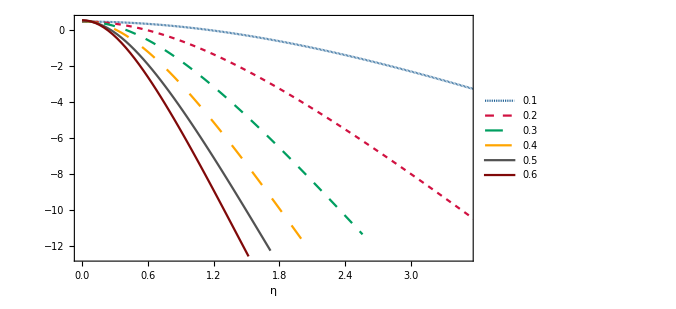

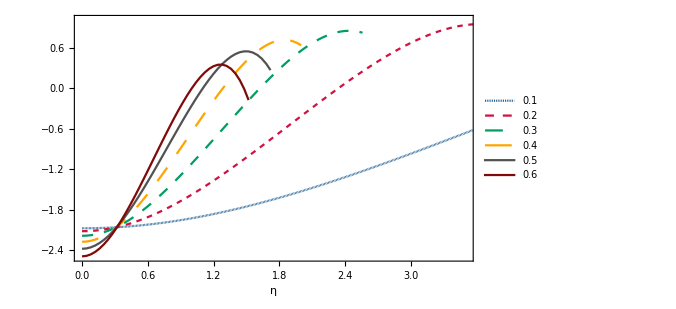

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.12,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
Max[Abs[(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100],Abs[(Max[Re[Tda[[2]]]]-Min[Re[Tda[[2]]]])/Min[Re[Tda[[2]]]]*100],Abs[(Max[Re[Tda[[3]]]]-Min[Re[Tda[[3]]]])/Min[Re[Tda[[3]]]]*100],Abs[(Max[Re[Tda[[4]]]]-Min[Re[Tda[[4]]]])/Min[Re[Tda[[4]]]]*100],Abs[(Max[Re[Tda[[5]]]]-Min[Re[Tda[[5]]]])/Min[Re[Tda[[5]]]]*100],Abs[(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100]]
Max[Abs[(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100],Abs[(Max[Im[Tda[[2]]]]-Min[Im[Tda[[2]]]])/Min[Im[Tda[[2]]]]*100],Abs[(Max[Im[Tda[[3]]]]-Min[Im[Tda[[3]]]])/Min[Im[Tda[[3]]]]*100],Abs[(Max[Im[Tda[[4]]]]-Min[Im[Tda[[4]]]])/Min[Im[Tda[[4]]]]*100],Abs[(Max[Im[Tda[[5]]]]-Min[Im[Tda[[5]]]])/Min[Im[Tda[[5]]]]*100],Abs[(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100]]
```

0.271854

1.38056

```mathematica
Max[Abs[(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100],Abs[(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100],Abs[(Max[Re[Tdp[[3]]]]-Min[Re[Tdp[[3]]]])/Min[Re[Tdp[[3]]]]*100],Abs[(Max[Re[Tdp[[4]]]]-Min[Re[Tdp[[4]]]])/Min[Re[Tdp[[4]]]]*100],Abs[(Max[Re[Tdp[[5]]]]-Min[Re[Tdp[[5]]]])/Min[Re[Tdp[[5]]]]*100],Abs[(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100],Abs[(Max[Im[Tdp[[2]]]]-Min[Im[Tdp[[2]]]])/Min[Im[Tdp[[2]]]]*100],Abs[(Max[Im[Tdp[[3]]]]-Min[Im[Tdp[[3]]]])/Min[Im[Tdp[[3]]]]*100],Abs[(Max[Im[Tdp[[4]]]]-Min[Im[Tdp[[4]]]])/Min[Im[Tdp[[4]]]]*100],Abs[(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100],Abs[(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100]]
```

15.3154

3.7695

### Isospectrality breaking m=-1 at=0.2

#### Axial modes

```mathematica
Ta={{{0.+0. ⅈ,0.23618546366973714-0.09317736589298987 ⅈ},{0.04+0.04 ⅈ,0.23618547864664557-0.0931773732879321 ⅈ},{0.08+0.08 ⅈ,0.23618552357879827-0.0931773954738842 ⅈ},{0.12+0.12 ⅈ,0.23618559847031512-0.09317743245413906 ⅈ},{0.16+0.16 ⅈ,0.2361857033280901-0.09317748423419801 ⅈ},{0.2+0.2 ⅈ,0.23618583816177613-0.09317755082176143 ⅈ},{0.24+0.24 ⅈ,0.23618600298378645-0.09317763222672747 ⅈ},{0.28+0.28 ⅈ,0.2361861978092957-0.09317772846119005 ⅈ},{0.32+0.32 ⅈ,0.23618642265624262-0.09317783953943688 ⅈ},{0.36+0.36 ⅈ,0.23618667754533196-0.09317796547794653 ⅈ},{0.4+0.4 ⅈ,0.2361869625000371-0.0931781062953856 ⅈ},{0.44+0.44 ⅈ,0.2361872775466035-0.0931782620126052 ⅈ},{0.48+0.48 ⅈ,0.23618762271405197-0.09317843265263692 ⅈ},{0.52+0.52 ⅈ,0.23618799803418195-0.0931786182406889 ⅈ},{0.56+0.56 ⅈ,0.23618840354157664-0.0931788188041408 ⅈ},{0.6+0.6 ⅈ,0.23618883927360648-0.09317903437253894 ⅈ},{0.64+0.64 ⅈ,0.2361893052704349-0.0931792649775904 ⅈ},{0.68+0.68 ⅈ,0.23618980157502253-0.09317951065315755 ⅈ},{0.72+0.72 ⅈ,0.2361903282331337-0.09317977143525129 ⅈ},{0.76+0.76 ⅈ,0.23619088529334192-0.09318004736202448 ⅈ},{0.8+0.8 ⅈ,0.236191472807036-0.09318033847376449 ⅈ},{0.84+0.84 ⅈ,0.23619209082842693-0.09318064481288571 ⅈ},{0.88+0.88 ⅈ,0.23619273941455474-0.09318096642392132 ⅈ},{0.92+0.92 ⅈ,0.2361934186252957-0.09318130335351484 ⅈ},{0.96+0.96 ⅈ,0.23619412852337024-0.09318165565041103 ⅈ},{1.+1. ⅈ,0.23619486917435067-0.09318202336544663 ⅈ},{1.04+1.04 ⅈ,0.23619564064666992-0.09318240655154324 ⅈ},{1.08+1.08 ⅈ,0.23619644301162898-0.09318280526368233 ⅈ},{1.12+1.12 ⅈ,0.23619727634340817-0.09318321955892382 ⅈ},{1.16+1.16 ⅈ,0.23619814071907447-0.09318364949636544 ⅈ},{1.2+1.2 ⅈ,0.23619903621859198-0.09318409513714576 ⅈ},{1.24+1.24 ⅈ,0.23619996292483206-0.09318455654442884 ⅈ},{1.28+1.28 ⅈ,0.23620092092358336-0.09318503378339182 ⅈ},{1.32+1.32 ⅈ,0.2362019103035628-0.09318552692121151 ⅈ},{1.36+1.36 ⅈ,0.23620293115642654-0.0931860360270507 ⅈ},{1.4+1.4 ⅈ,0.23620398357678102-0.09318656117204438 ⅈ},{1.44+1.44 ⅈ,0.23620506766219487-0.09318710242928456 ⅈ},{1.48+1.48 ⅈ,0.2362061835132111-0.09318765987380548 ⅈ},{1.52+1.52 ⅈ,0.23620733123335869-0.0931882335825678 ⅈ},{1.56+1.56 ⅈ,0.23620851092916603-0.09318882363444238 ⅈ},{1.6+1.6 ⅈ,0.23620972271017326-0.0931894301101936 ⅈ},{1.64+1.64 ⅈ,0.23621096668894553-0.09319005309246212 ⅈ},{1.68+1.68 ⅈ,0.2362122429810869-0.09319069266574698 ⅈ},{1.72+1.72 ⅈ,0.23621355170525365-0.09319134891638742 ⅈ},{1.76+1.76 ⅈ,0.23621489298316883-0.09319202193254375 ⅈ},{1.8+1.8 ⅈ,0.23621626693963635-0.09319271180417825 ⅈ},{1.84+1.84 ⅈ,0.23621767370255561-0.09319341862303476 ⅈ},{1.88+1.88 ⅈ,0.23621911340293708-0.0931941424826183 ⅈ},{1.92+1.92 ⅈ,0.2362205861749167-0.09319488347817385 ⅈ},{1.96+1.96 ⅈ,0.236222092155772-0.09319564170666456 ⅈ},{2.+2. ⅈ,0.23622363148593772-0.09319641726674927 ⅈ},{2.04+2.04 ⅈ,0.23622520430902166-0.09319721025875971 ⅈ},{2.08+2.08 ⅈ,0.23622681077182126-0.09319802078467683 ⅈ},{2.12+2.12 ⅈ,0.23622845102434012-0.09319884894810636 ⅈ},{2.16+2.16 ⅈ,0.23623012521980472-0.09319969485425426 ⅈ},{2.2+2.2 ⅈ,0.23623183351468147-0.09320055860990101 ⅈ},{2.24+2.24 ⅈ,0.23623357606869422-0.09320144032337546 ⅈ},{2.28+2.28 ⅈ,0.23623535304484128-0.09320234010452809 ⅈ},{2.32+2.32 ⅈ,0.2362371646094138-0.09320325806470324 ⅈ},{2.36+2.36 ⅈ,0.2362390109320133-0.09320419431671137 ⅈ},{2.4+2.4 ⅈ,0.23624089218556985-0.09320514897479976 ⅈ},{2.44+2.44 ⅈ,0.23624280854636073-0.09320612215462307 ⅈ},{2.48+2.48 ⅈ,0.23624476019402857-0.09320711397321305 ⅈ},{2.52+2.52 ⅈ,0.23624674731160059-0.09320812454894754 ⅈ},{2.56+2.56 ⅈ,0.23624877008550715-0.0932091540015186 ⅈ},{2.6+2.6 ⅈ,0.23625082870560102-0.09321020245190012 ⅈ},{2.64+2.64 ⅈ,0.23625292336517645-0.09321127002231443 ⅈ},{2.68+2.68 ⅈ,0.23625505426098908-0.09321235683619836 ⅈ},{2.72+2.72 ⅈ,0.2362572215932749-0.09321346301816837 ⅈ},{2.76+2.76 ⅈ,0.23625942556577034-0.09321458869398491 ⅈ},{2.8+2.8 ⅈ,0.23626166638573204-0.09321573399051608 ⅈ},{2.84+2.84 ⅈ,0.23626394426395655-0.09321689903570039 ⅈ},{2.88+2.88 ⅈ,0.2362662594148008-0.09321808395850861 ⅈ},{2.92+2.92 ⅈ,0.2362686120562019-0.09321928888890492 ⅈ},{2.96+2.96 ⅈ,0.23627100240969737-0.09322051395780723 ⅈ},{3.+3. ⅈ,0.23627343070044568-0.0932217592970465 ⅈ},{3.04+3.04 ⅈ,0.23627589715724656-0.09322302503932516 ⅈ},{3.08+3.08 ⅈ,0.23627840201256106-0.09322431131817496 ⅈ},{3.12+3.12 ⅈ,0.2362809455025325-0.09322561826791347 ⅈ},{3.16+3.16 ⅈ,0.2362835278670065-0.09322694602359986 ⅈ},{3.2+3.2 ⅈ,0.23628614934955178-0.09322829472099002 ⅈ},{3.24+3.24 ⅈ,0.2362888101974803-0.09322966449649028 ⅈ},{3.28+3.28 ⅈ,0.2362915106618681-0.09323105548711041 ⅈ},{3.32+3.32 ⅈ,0.23629425099757548-0.09323246783041565 ⅈ},{3.36+3.36 ⅈ,0.23629703146326717-0.09323390166447774 ⅈ},{3.4+3.4 ⅈ,0.23629985232143316-0.09323535712782503 ⅈ},{3.44+3.44 ⅈ,0.2363027138384084-0.09323683435939123 ⅈ},{3.48+3.48 ⅈ,0.23630561628439323-0.0932383334984638 ⅈ},{3.52+3.52 ⅈ,0.23630855993347327-0.09323985468463054 ⅈ},{3.56+3.56 ⅈ,0.23631154506363927-0.09324139805772576 ⅈ},{3.6+3.6 ⅈ,0.23631457195680697-0.09324296375777502 ⅈ},{3.64+3.64 ⅈ,0.2363176408988366-0.09324455192493884 ⅈ},{3.68+3.68 ⅈ,0.23632075217955206-0.09324616269945557 ⅈ},{3.72+3.72 ⅈ,0.23632390609276027-0.09324779622158268 ⅈ},{3.76+3.76 ⅈ,0.23632710293627013-0.09324945263153755 ⅈ},{3.8+3.8 ⅈ,0.23633034301191114-0.09325113206943646 ⅈ},{3.84+3.84 ⅈ,0.23633362662555163-0.09325283467523302 ⅈ},{3.88+3.88 ⅈ,0.23633695408711716-0.093254560588655 ⅈ},{3.92+3.92 ⅈ,0.23634032571060823-0.09325630994914037 ⅈ},{3.96+3.96 ⅈ,0.2363437418141175-0.09325808289577159 ⅈ},{4.+4. ⅈ,0.23634720271984733-0.09325987956720946 ⅈ},{4.04+4.04 ⅈ,0.23635070875412595-0.0932617001016252 ⅈ},{4.08+4.08 ⅈ,0.23635426024742417-0.09326354463663125 ⅈ},{4.12+4.12 ⅈ,0.23635785753437102-0.09326541330921129 ⅈ},{4.16+4.16 ⅈ,0.2363615009537692-0.09326730625564872 ⅈ},{4.2+4.2 ⅈ,0.23636519084860994-0.09326922361145364 ⅈ},{4.24+4.24 ⅈ,0.23636892756608727-0.09327116551128911 ⅈ},{4.28+4.28 ⅈ,0.23637271145761193-0.09327313208889555 ⅈ},{4.32+4.32 ⅈ,0.23637654287882462-0.09327512347701429 ⅈ},{4.36+4.36 ⅈ,0.23638042218960842-0.09327713980730944 ⅈ},{4.4+4.4 ⅈ,0.23638434975410078-0.09327918121028866 ⅈ},{4.44+4.44 ⅈ,0.2363883259407053-0.09328124781522237 ⅈ},{4.48+4.48 ⅈ,0.2363923511221013-0.09328333975006192 ⅈ},{4.52+4.52 ⅈ,0.23639642567525465-0.0932854571413562 ⅈ},{4.56+4.56 ⅈ,0.2364005499814261-0.09328760011416669 ⅈ},{4.6+4.6 ⅈ,0.23640472442617994-0.09328976879198142 ⅈ},{4.64+4.64 ⅈ,0.2364089493993911-0.09329196329662758 ⅈ},{4.68+4.68 ⅈ,0.23641322529525183-0.09329418374818226 ⅈ},{4.72+4.72 ⅈ,0.23641755251227706-0.09329643026488224 ⅈ},{4.76+4.76 ⅈ,0.2364219314533092-0.09329870296303217 ⅈ},{4.8+4.8 ⅈ,0.23642636252552146-0.09330100195691145 ⅈ},{4.84+4.84 ⅈ,0.23643084614042065-0.09330332735867913 ⅈ},{4.88+4.88 ⅈ,0.2364353827138483-0.09330567927827826 ⅈ},{4.92+4.92 ⅈ,0.2364399726659814-0.09330805782333791 ⅈ},{4.96+4.96 ⅈ,0.23644461642133105-0.09331046309907441 ⅈ},{5.+5. ⅈ,0.2364493144087406-0.09331289520819053 ⅈ},{5.04+5.04 ⅈ,0.23645406706138228-0.0933153542507735 ⅈ},{5.08+5.08 ⅈ,0.23645887481675248-0.09331784032419181 ⅈ},{5.12+5.12 ⅈ,0.23646373811666566-0.09332035352298977 ⅈ},{5.16+5.16 ⅈ,0.236468657407247-0.09332289393878133 ⅈ},{5.2+5.2 ⅈ,0.23647363313892322-0.09332546166014206 ⅈ},{5.24+5.24 ⅈ,0.23647866576641244-0.09332805677249967 ⅈ},{5.28+5.28 ⅈ,0.2364837557487119-0.09333067935802287 ⅈ},{5.32+5.32 ⅈ,0.23648890354908453-0.0933333294955094 ⅈ},{5.36+5.36 ⅈ,0.2364941096350436-0.09333600726027165 ⅈ},{5.4+5.4 ⅈ,0.23649937447833544-0.09333871272402139 ⅈ},{5.44+5.44 ⅈ,0.23650469855492098-0.09334144595475292 ⅈ},{5.48+5.48 ⅈ,0.23651008234495488-0.09334420701662455 ⅈ},{5.52+5.52 ⅈ,0.23651552633276282-0.093346995969839 ⅈ},{5.56+5.56 ⅈ,0.23652103100681732-0.09334981287052178 ⅈ},{5.6+5.6 ⅈ,0.23652659685971072-0.09335265777059863 ⅈ},{5.64+5.64 ⅈ,0.2365322243881272-0.09335553071767128 ⅈ},{5.68+5.68 ⅈ,0.23653791409281127-0.09335843175489157 ⅈ},{5.72+5.72 ⅈ,0.23654366647853506-0.09336136092083476 ⅈ},{5.76+5.76 ⅈ,0.2365494820540633-0.0933643182493707 ⅈ},{5.8+5.8 ⅈ,0.2365553613321152-0.09336730376953406 ⅈ},{5.84+5.84 ⅈ,0.23656130482932494-0.0933703175053933 ⅈ},{5.88+5.88 ⅈ,0.23656731306619874-0.0933733594759176 ⅈ},{5.92+5.92 ⅈ,0.23657338656707005-0.09337642969484342 ⅈ},{5.96+5.96 ⅈ,0.23657952586005182-0.09337952817053888 ⅈ},{6.+6. ⅈ,0.23658573147698608-0.09338265490586736 ⅈ},{6.04+6.04 ⅈ,0.23659200395339103-0.0933858098980498 ⅈ},{6.08+6.08 ⅈ,0.23659834382840494-0.09338899313852551 ⅈ},{6.12+6.12 ⅈ,0.23660475164472716-0.09339220461281188 ⅈ},{6.16+6.16 ⅈ,0.23661122794855682-0.09339544430036323 ⅈ},{6.2+6.2 ⅈ,0.23661777328952735-0.0933987121744281 ⅈ},{6.24+6.24 ⅈ,0.23662438822063883-0.09340200820190564 ⅈ},{6.28+6.28 ⅈ,0.23663107329818678-0.09340533234320089 ⅈ},{6.32+6.32 ⅈ,0.2366378290816874-0.0934086845520792 ⅈ},{6.36+6.36 ⅈ,0.23664465613380037-0.09341206477551942 ⅈ},{6.4+6.4 ⅈ,0.23665155502024646-0.09341547295356642 ⅈ},{6.44+6.44 ⅈ,0.2366585263097239-0.09341890901918252 ⅈ},{6.48+6.48 ⅈ,0.2366655705738191-0.09342237289809834 ⅈ},{6.52+6.52 ⅈ,0.23667268838691527-0.09342586450866248 ⅈ},{6.56+6.56 ⅈ,0.23667988032609563-0.0934293837616912 ⅈ},{6.6+6.6 ⅈ,0.23668714697104484-0.09343293056031654 ⅈ},{6.64+6.64 ⅈ,0.23669448890394454-0.0934365047998347 ⅈ},{6.68+6.68 ⅈ,0.23670190670936603-0.09344010636755347 ⅈ},{6.72+6.72 ⅈ,0.2367094009741586-0.09344373514263896 ⅈ},{6.76+6.76 ⅈ,0.23671697228733357-0.09344739099596291 ⅈ},{6.8+6.8 ⅈ,0.23672462123994426-0.09345107378994856 ⅈ},{6.84+6.84 ⅈ,0.23673234842496127-0.0934547833784172 ⅈ},{6.88+6.88 ⅈ,0.2367401544371441-0.09345851960643395 ⅈ},{6.92+6.92 ⅈ,0.23674803987290716-0.09346228231015402 ⅈ},{6.96+6.96 ⅈ,0.23675600533018235-0.09346607131666884 ⅈ},{7.+7. ⅈ,0.23676405140827622-0.09346988644385204 ⅈ},{7.04+7.04 ⅈ,0.23677217870772257-0.09347372750020624 ⅈ},{7.08+7.08 ⅈ,0.23678038783013036-0.09347759428470975 ⅈ},{7.12+7.12 ⅈ,0.23678867937802675-0.09348148658666394 ⅈ}},{{0.+0. ⅈ,0.23738966082421634-0.09337472518516488 ⅈ},{0.04+0.04 ⅈ,0.2373897258464749-0.0933747516389925 ⅈ},{0.08+0.08 ⅈ,0.23738992093465242-0.09337483101710277 ⅈ},{0.12+0.12 ⅈ,0.2373902461523139-0.09337496336910087 ⅈ},{0.16+0.16 ⅈ,0.23739070160554623-0.09337514877766466 ⅈ},{0.2+0.2 ⅈ,0.2373912874429465-0.09337538735845531 ⅈ},{0.24+0.24 ⅈ,0.23739200385569847-0.09337567926002963 ⅈ},{0.28+0.28 ⅈ,0.23739285107766947-0.09337602466372673 ⅈ},{0.32+0.32 ⅈ,0.23739382938552978-0.09337642378352924 ⅈ},{0.36+0.36 ⅈ,0.23739493909889234-0.0933768768658989 ⅈ},{0.4+0.4 ⅈ,0.2373961805804751-0.09337738418958583 ⅈ},{0.44+0.44 ⅈ,0.2373975542362831-0.09337794606541146 ⅈ},{0.48+0.48 ⅈ,0.23739906051581267-0.09337856283602487 ⅈ},{0.52+0.52 ⅈ,0.23740069991227614-0.09337923487563188 ⅈ},{0.56+0.56 ⅈ,0.237402472962847-0.09337996258969658 ⅈ},{0.6+0.6 ⅈ,0.23740438024892568-0.09338074641461443 ⅈ},{0.64+0.64 ⅈ,0.23740642239642606-0.0933815868173575 ⅈ},{0.68+0.68 ⅈ,0.23740860007608094-0.09338248429508961 ⅈ},{0.72+0.72 ⅈ,0.23741091400376838-0.09338343937475219 ⅈ},{0.76+0.76 ⅈ,0.2374133649408564-0.09338445261261948 ⅈ},{0.8+0.8 ⅈ,0.2374159536945676-0.09338552459382234 ⅈ},{0.84+0.84 ⅈ,0.23741868111836206-0.09338665593184053 ⅈ},{0.88+0.88 ⅈ,0.23742154811233837-0.09338784726796166 ⅈ},{0.92+0.92 ⅈ,0.23742455562365286-0.09338909927070696 ⅈ},{0.96+0.96 ⅈ,0.23742770464695656-0.09339041263522219 ⅈ},{1.+1. ⅈ,0.23743099622484803-0.0933917880826334 ⅈ},{1.04+1.04 ⅈ,0.2374344314483435-0.0933932263593662 ⅈ},{1.08+1.08 ⅈ,0.23743801145736232-0.0933947282364273 ⅈ},{1.12+1.12 ⅈ,0.23744173744122785-0.09339629450864802 ⅈ},{1.16+1.16 ⅈ,0.23744561063918243-0.09339792599388776 ⅈ},{1.2+1.2 ⅈ,0.23744963234091604-0.093399623532197 ⅈ},{1.24+1.24 ⅈ,0.2374538038871085-0.09340138798493816 ⅈ},{1.28+1.28 ⅈ,0.2374581266699827-0.09340322023386331 ⅈ},{1.32+1.32 ⅈ,0.23746260213386997-0.09340512118014747 ⅈ},{1.36+1.36 ⅈ,0.2374672317757851-0.09340709174337603 ⅈ},{1.4+1.4 ⅈ,0.23747201714601032-0.09340913286048497 ⅈ},{1.44+1.44 ⅈ,0.2374769598486878-0.09341124548465277 ⅈ},{1.48+1.48 ⅈ,0.2374820615424185-0.09341343058414206 ⅈ},{1.52+1.52 ⅈ,0.23748732394086688-0.09341568914109005 ⅈ},{1.56+1.56 ⅈ,0.23749274881336938-0.09341802215024568 ⅈ},{1.6+1.6 ⅈ,0.23749833798554587-0.09342043061765275 ⅈ},{1.64+1.64 ⅈ,0.23750409333991232-0.09342291555927638 ⅈ},{1.68+1.68 ⅈ,0.23751001681649286-0.09342547799957251 ⅈ},{1.72+1.72 ⅈ,0.23751611041342915-0.09342811896999731 ⅈ},{1.76+1.76 ⅈ,0.2375223761875867-0.0934308395074564 ⅈ},{1.8+1.8 ⅈ,0.23752881625515396-0.09343364065269107 ⅈ},{1.84+1.84 ⅈ,0.2375354327922337-0.09343652344860004 ⅈ},{1.88+1.88 ⅈ,0.23754222803542394-0.09343948893849581 ⅈ},{1.92+1.92 ⅈ,0.23754920428238605-0.09344253816429271 ⅈ},{1.96+1.96 ⅈ,0.23755636389239757-0.09344567216462592 ⅈ},{2.+2. ⅈ,0.23756370928688667-0.09344889197289925 ⅈ},{2.04+2.04 ⅈ,0.23757124294994625-0.09345219861526013 ⅈ},{2.08+2.08 ⅈ,0.23757896742882423-0.09345559310849999 ⅈ},{2.12+2.12 ⅈ,0.23758688533438688-0.09345907645787879 ⅈ},{2.16+2.16 ⅈ,0.23759499934155137-0.09346264965487114 ⅈ},{2.2+2.2 ⅈ,0.23760331218968603-0.09346631367483378 ⅈ},{2.24+2.24 ⅈ,0.23761182668297173-0.09347006947459138 ⅈ},{2.28+2.28 ⅈ,0.2376205456907229-0.0934739179899401 ⅈ},{2.32+2.32 ⅈ,0.23762947214766317-0.09347786013306747 ⅈ},{2.36+2.36 ⅈ,0.2376386090541511-0.09348189678988629 ⅈ},{2.4+2.4 ⅈ,0.23764795947635226-0.09348602881728268 ⅈ},{2.44+2.44 ⅈ,0.23765752654635205-0.09349025704027561 ⅈ},{2.48+2.48 ⅈ,0.23766731346220565-0.09349458224908802 ⅈ},{2.52+2.52 ⅈ,0.23767732348791792-0.09349900519612783 ⅈ},{2.56+2.56 ⅈ,0.23768755995335034-0.09350352659287832 ⅈ},{2.6+2.6 ⅈ,0.23769802625404665-0.09350814710669723 ⅈ},{2.64+2.64 ⅈ,0.23770872585097436-0.09351286735752373 ⅈ},{2.68+2.68 ⅈ,0.23771966227017235-0.09351768791449379 ⅈ},{2.72+2.72 ⅈ,0.2377308391023016-0.09352260929246274 ⅈ},{2.76+2.76 ⅈ,0.23774226000209045-0.09352763194843605 ⅈ},{2.8+2.8 ⅈ,0.23775392868766748-0.09353275627790845 ⅈ},{2.84+2.84 ⅈ,0.2377658489397759-0.09353798261111192 ⅈ},{2.88+2.88 ⅈ,0.2377780246008608-0.09354331120917361 ⅈ},{2.92+2.92 ⅈ,0.2377904595740222-0.09354874226018538 ⅈ},{2.96+2.96 ⅈ,0.2378031578218262-0.09355427587518572 ⅈ},{3.+3. ⅈ,0.23781612336496497-0.09355991208405713 ⅈ},{3.04+3.04 ⅈ,0.23782936028075793-0.09356565083134098 ⅈ},{3.08+3.08 ⅈ,0.23784287270148566-0.09357149197197236 ⅈ},{3.12+3.12 ⅈ,0.23785666481254628-0.09357743526693901 ⅈ},{3.16+3.16 ⅈ,0.23787074085042625-0.0935834803788678 ⅈ},{3.2+3.2 ⅈ,0.2378851051004764-0.09358962686754331 ⅈ},{3.24+3.24 ⅈ,0.23789976189448203-0.09359587418536376 ⅈ},{3.28+3.28 ⅈ,0.23791471560801908-0.09360222167273938 ⅈ},{3.32+3.32 ⅈ,0.23792997065758545-0.09360866855343998 ⅈ},{3.36+3.36 ⅈ,0.2379455314974975-0.09361521392989895 ⅈ},{3.4+3.4 ⅈ,0.23796140261654222-0.0936218567784809 ⅈ},{3.44+3.44 ⅈ,0.23797758853437367-0.09362859594472127 ⅈ},{3.48+3.48 ⅈ,0.23799409379764447-0.0936354301385485 ⅈ},{3.52+3.52 ⅈ,0.2380109229758619-0.09364235792949747 ⅈ},{3.56+3.56 ⅈ,0.23802808065695807-0.09364937774192636 ⅈ},{3.6+3.6 ⅈ,0.23804557144256436-0.09365648785024817 ⅈ},{3.64+3.64 ⅈ,0.23806339994297945-0.09366368637419074 ⅈ}},{{0.+0. ⅈ,0.23937116397928698-0.093701683419257 ⅈ},{0.04+0.04 ⅈ,0.23937132926100213-0.09370173201207097 ⅈ},{0.08+0.08 ⅈ,0.2393718252074161-0.09370187786589455 ⅈ},{0.12+0.12 ⅈ,0.23937265212079223-0.093702121206252 ⅈ},{0.16+0.16 ⅈ,0.2393738105055489-0.09370246240864731 ⅈ},{0.2+0.2 ⅈ,0.23937530106864807-0.09370290199783793 ⅈ},{0.24+0.24 ⅈ,0.2393771247203714-0.09370344064688223 ⅈ},{0.28+0.28 ⅈ,0.23937928257531393-0.09370407917590919 ⅈ},{0.32+0.32 ⅈ,0.239381775953596-0.09370481855060508 ⅈ},{0.36+0.36 ⅈ,0.2393846063822904-0.09370565988041224 ⅈ},{0.4+0.4 ⅈ,0.23938777559706126-0.09370660441643304 ⅈ},{0.44+0.44 ⅈ,0.23939128554401312-0.0937076535490319 ⅈ},{0.48+0.48 ⅈ,0.23939513838174498-0.09370880880512611 ⅈ},{0.52+0.52 ⅈ,0.2393993364836054-0.09371007184515628 ⅈ},{0.56+0.56 ⅈ,0.2394038824401446-0.09371144445972622 ⅈ},{0.6+0.6 ⅈ,0.23940877906175626-0.09371292856589955 ⅈ},{0.64+0.64 ⅈ,0.23941402938150425-0.09371452620314122 ⅈ},{0.68+0.68 ⅈ,0.2394196366581257-0.09371623952888966 ⅈ},{0.72+0.72 ⅈ,0.23942560437920343-0.09371807081374513 ⅈ},{0.76+0.76 ⅈ,0.2394319362644974-0.09372002243625825 ⅈ},{0.8+0.8 ⅈ,0.23943863626942635-0.09372209687730174 ⅈ},{0.84+0.84 ⅈ,0.23944570858868683-0.0937242967140078 ⅈ},{0.88+0.88 ⅈ,0.23945315765999803-0.09372662461325201 ⅈ},{0.92+0.92 ⅈ,0.2394609881679578-0.09372908332466372 ⅈ},{0.96+0.96 ⅈ,0.2394692050479947-0.09373167567314258 ⅈ},{1.+1. ⅈ,0.23947781349039773-0.09373440455085863 ⅈ},{1.04+1.04 ⅈ,0.23948681894440674-0.09373727290871407 ⅈ},{1.08+1.08 ⅈ,0.23949622712233956-0.09374028374724233 ⅈ},{1.12+1.12 ⅈ,0.23950604400373685-0.09374344010692083 ⅈ},{1.16+1.16 ⅈ,0.23951627583949403-0.09374674505787166 ⅈ},{1.2+1.2 ⅈ,0.2395269291559579-0.09375020168892463 ⅈ},{1.24+1.24 ⅈ,0.23953801075895295-0.09375381309601681 ⅈ},{1.28+1.28 ⅈ,0.23954952773770696-0.09375758236990082 ⅈ},{1.32+1.32 ⅈ,0.239561487468638-0.0937615125831358 ⅈ},{1.36+1.36 ⅈ,0.2395738976189639-0.09376560677633282 ⅈ},{1.4+1.4 ⅈ,0.23958676615009-0.09376986794362877 ⅈ},{1.44+1.44 ⅈ,0.23960010132072956-0.0937742990173598 ⅈ},{1.48+1.48 ⅈ,0.23961391168970536-0.09377890285190976 ⅈ},{1.52+1.52 ⅈ,0.23962820611837635-0.09378368220670599 ⅈ},{1.56+1.56 ⅈ,0.23964299377263243-0.09378863972833876 ⅈ},{1.6+1.6 ⅈ,0.23965828412438955-0.09379377793177983 ⅈ},{1.64+1.64 ⅈ,0.23967408695251935-0.09379909918067862 ⅈ},{1.68+1.68 ⅈ,0.2396904123431362-0.09380460566671618 ⅈ},{1.72+1.72 ⅈ,0.23970727068916364-0.0938102993879993 ⅈ},{1.76+1.76 ⅈ,0.23972467268909292-0.09381618212648074 ⅈ},{1.8+1.8 ⅈ,0.23974262934484455-0.09382225542439492 ⅈ},{1.84+1.84 ⅈ,0.23976115195863298-0.09382852055970246 ⅈ},{1.88+1.88 ⅈ,0.23978025212873177-0.09383497852054234 ⅈ},{1.92+1.92 ⅈ,0.23979994174403013-0.09384162997869593 ⅈ},{1.96+1.96 ⅈ,0.2398202329772626-0.09384847526207271 ⅈ},{2.+2. ⅈ,0.23984113827678988-0.09385551432623718 ⅈ},{2.04+2.04 ⅈ,0.23986267035680212-0.09386274672500201 ⅈ},{2.08+2.08 ⅈ,0.2398848421858071-0.09387017158012355 ⅈ},{2.12+2.12 ⅈ,0.23990766697326377-0.09387778755014606 ⅈ},{2.16+2.16 ⅈ,0.23993115815421207-0.093885592798452 ⅈ},{2.2+2.2 ⅈ,0.23995532937174596-0.09389358496058949 ⅈ},{2.24+2.24 ⅈ,0.2399801944571724-0.09390176111096098 ⅈ},{2.28+2.28 ⅈ,0.24000576740769375-0.09391011772897451 ⅈ},{2.32+2.32 ⅈ,0.240032062361448-0.09391865066477398 ⅈ},{2.36+2.36 ⅈ,0.24005909356973903-0.0939273551046846 ⅈ},{2.4+2.4 ⅈ,0.24008687536628756-0.09393622553652978 ⅈ},{2.44+2.44 ⅈ,0.2401154221333353-0.0939452557149955 ⅈ},{2.48+2.48 ⅈ,0.24014474826443477-0.09395443862724408 ⅈ},{2.52+2.52 ⅈ,0.24017486812376257-0.09396376645900055 ⅈ},{2.56+2.56 ⅈ,0.24020579600180236-0.09397323056136342 ⅈ}},{{0.+0. ⅈ,0.24209307389684026-0.09415506220756345 ⅈ},{0.04+0.04 ⅈ,0.24209341418935137-0.09415512416129818 ⅈ},{0.08+0.08 ⅈ,0.24209443536086006-0.0941553102252561 ⅈ},{0.12+0.12 ⅈ,0.2420961382904258-0.09415562100636964 ⅈ},{0.16+0.16 ⅈ,0.24209852444550295-0.0941560575139272 ⅈ},{0.2+0.2 ⅈ,0.24210159588427396-0.09415662115594259 ⅈ},{0.24+0.24 ⅈ,0.24210535525938218-0.09415731373412803 ⅈ},{0.28+0.28 ⅈ,0.24210980582270872-0.09415813743737712 ⅈ},{0.32+0.32 ⅈ,0.24211495143117712-0.0941590948337185 ⅈ},{0.36+0.36 ⅈ,0.24212079655356505-0.09416018886069076 ⅈ},{0.4+0.4 ⅈ,0.24212734627829613-0.09416142281408015 ⅈ},{0.44+0.44 ⅈ,0.24213460632218078-0.09416280033495443 ⅈ},{0.48+0.48 ⅈ,0.24214258304006814-0.09416432539491591 ⅈ},{0.52+0.52 ⅈ,0.242151283435365-0.09416600227948785 ⅈ},{0.56+0.56 ⅈ,0.24216071517136945-0.09416783556953995 ⅈ},{0.6+0.6 ⅈ,0.2421708865833586-0.09416983012064778 ⅈ},{0.64+0.64 ⅈ,0.2421818066913609-0.09417199104027321 ⅈ},{0.68+0.68 ⅈ,0.2421934852135317-0.09417432366264289 ⅈ},{0.72+0.72 ⅈ,0.24220593258003914-0.09417683352119346 ⅈ},{0.76+0.76 ⅈ,0.24221915994735546-0.09417952631844267 ⅈ},{0.8+0.8 ⅈ,0.2422331792128299-0.09418240789313785 ⅈ},{0.84+0.84 ⅈ,0.24224800302940888-0.09418548418452415 ⅈ},{0.88+0.88 ⅈ,0.2422636448203428-0.0941887611935692 ⅈ},{0.92+0.92 ⅈ,0.24228011879370667-0.09419224494097199 ⅈ},{0.96+0.96 ⅈ,0.2422974399565307-0.0941959414217796 ⅈ},{1.+1. ⅈ,0.24231562412831964-0.09419985655643069 ⅈ},{1.04+1.04 ⅈ,0.24233468795370525-0.09420399613804023 ⅈ},{1.08+1.08 ⅈ,0.24235464891395175-0.09420836577574036 ⅈ},{1.12+1.12 ⅈ,0.2423755253369974-0.09421297083389212 ⅈ},{1.16+1.16 ⅈ,0.24239733640568084-0.09421781636698522 ⅈ},{1.2+1.2 ⅈ,0.2424201021637629-0.09422290705005205 ⅈ},{1.24+1.24 ⅈ,0.24244384351931036-0.09422824710442874 ⅈ},{1.28+1.28 ⅈ,0.2424685822449666-0.09423384021871248 ⅈ},{1.32+1.32 ⅈ,0.24249434097458217-0.09423968946478262 ⅈ},{1.36+1.36 ⅈ,0.24252114319563153-0.09424579720877664 ⅈ},{1.4+1.4 ⅈ,0.24254901323678396-0.09425216501694475 ⅈ},{1.44+1.44 ⅈ,0.24257797624994598-0.09425879355634334 ⅈ},{1.48+1.48 ⅈ,0.24260805818602815-0.09426568249037545 ⅈ},{1.52+1.52 ⅈ,0.2426392857636348-0.09427283036924135 ⅈ},{1.56+1.56 ⅈ,0.24267168642981182-0.09428023451542945 ⅈ},{1.6+1.6 ⅈ,0.24270528831192664-0.09428789090445597 ⅈ},{1.64+1.64 ⅈ,0.24274012015969806-0.09429579404115165 ⅈ},{1.68+1.68 ⅈ,0.24277621127633411-0.09430393683190116 ⅈ},{1.72+1.72 ⅈ,0.24281359143768652-0.09431231045335949 ⅈ},{1.76+1.76 ⅈ,0.24285229079828388-0.09432090421830737 ⅈ},{1.8+1.8 ⅈ,0.24289233978306912-0.09432970543946397 ⅈ},{1.84+1.84 ⅈ,0.2429337689636443-0.09433869929224617 ⅈ},{1.88+1.88 ⅈ,0.24297660891781558-0.0943478686776578 ⅈ},{1.92+1.92 ⅈ,0.24302089007124145-0.09435719408670426 ⅈ},{1.96+1.96 ⅈ,0.24306664252002422-0.09436665346795778 ⅈ},{2.+2. ⅈ,0.2431138958331454-0.09437622210015068 ⅈ}},{{0.+0. ⅈ,0.2455062756179261-0.09473004542157572 ⅈ},{0.04+0.04 ⅈ,0.24550689842079448-0.09473009986094712 ⅈ},{0.08+0.08 ⅈ,0.24550876747942327-0.09473026357342289 ⅈ},{0.12+0.12 ⅈ,0.24551188473933291-0.09473053773903398 ⅈ},{0.16+0.16 ⅈ,0.24551625344967742-0.09473092431620014 ⅈ},{0.2+0.2 ⅈ,0.2455218781709604-0.0947314260290122 ⅈ},{0.24+0.24 ⅈ,0.24552876478664254-0.09473204634934335 ⅈ},{0.28+0.28 ⅈ,0.24553692051794476-0.09473278947357446 ⅈ},{0.32+0.32 ⅈ,0.24554635394175556-0.09473366029372737 ⅈ},{0.36+0.36 ⅈ,0.24555707501151802-0.0947346643627514 ⅈ},{0.4+0.4 ⅈ,0.2455690950809486-0.09473580785366303 ⅈ},{0.44+0.44 ⅈ,0.2455824269303987-0.09473709751218963 ⅈ},{0.48+0.48 ⅈ,0.24559708479563622-0.09473854060252106 ⅈ},{0.52+0.52 ⅈ,0.2456130843987745-0.09474014484572449 ⅈ},{0.56+0.56 ⅈ,0.24563044298102552-0.09474191835033018 ⅈ},{0.6+0.6 ⅈ,0.2456491793368956-0.09474386953454916 ⅈ},{0.64+0.64 ⅈ,0.24566931384936883-0.09474600703953667 ⅈ},{0.68+0.68 ⅈ,0.2456908685255498-0.09474833963307211 ⅈ},{0.72+0.72 ⅈ,0.245713867032141-0.09475087610298387 ⅈ},{0.76+0.76 ⅈ,0.245738334730034-0.09475362513961044 ⅈ},{0.8+0.8 ⅈ,0.24576429870717229-0.09475659520655609 ⅈ},{0.84+0.84 ⅈ,0.24579178780871605-0.09475979439897447 ⅈ},{0.88+0.88 ⅈ,0.24582083266338864-0.0947632302885974 ⅈ},{0.92+0.92 ⅈ,0.24585146570472327-0.09476690975472116 ⅈ},{0.96+0.96 ⅈ,0.24588372118574053-0.0947708388003717 ⅈ},{1.+1. ⅈ,0.24591763518538842-0.09477502235290107 ⅈ},{1.04+1.04 ⅈ,0.24595324560484905-0.09477946404831422 ⅈ},{1.08+1.08 ⅈ,0.24599059215157326-0.09478416599870601 ⅈ},{1.12+1.12 ⅈ,0.24602971630864023-0.09478912854229869 ⅈ},{1.16+1.16 ⅈ,0.24607066128675015-0.09479434997571676 ⅈ},{1.2+1.2 ⅈ,0.24611347195585923-0.09479982626833751 ⅈ},{1.24+1.24 ⅈ,0.24615819475314213-0.0948055507588021 ⅈ},{1.28+1.28 ⅈ,0.24620487756364143-0.09481151383408902 ⅈ},{1.32+1.32 ⅈ,0.24625356956962283-0.09481770259193696 ⅈ},{1.36+1.36 ⅈ,0.24630432106432734-0.09482410048787827 ⅈ},{1.4+1.4 ⅈ,0.24635718322548733-0.09483068696870608 ⅈ},{1.44+1.44 ⅈ,0.24641220784368628-0.09483743709487144 ⅈ},{1.48+1.48 ⅈ,0.24646944700039145-0.09484432115509062 ⅈ},{1.52+1.52 ⅈ,0.24652895269031186-0.09485130427735648 ⅈ},{1.56+1.56 ⅈ,0.24659077638264826-0.09485834604158959 ⅈ},{1.6+1.6 ⅈ,0.2466549685158362-0.09486540010034727 ⅈ},{1.64+1.64 ⅈ,0.24672157792059174-0.0948724138153287 ⅈ},{1.68+1.68 ⅈ,0.24679065116646953-0.09487932791886292 ⅈ},{1.72+1.72 ⅈ,0.24686223182780623-0.09488607621113873 ⅈ}},{{0.+0. ⅈ,0.2495516907066438-0.09541995330947824 ⅈ},{0.04+0.04 ⅈ,0.2495527426853906-0.09541997018614308 ⅈ},{0.08+0.08 ⅈ,0.24955589983343696-0.09542002140916764 ⅈ},{0.12+0.12 ⅈ,0.24956116577957588-0.09542010875053167 ⅈ},{0.16+0.16 ⅈ,0.24956854658649402-0.0954202351403399 ⅈ},{0.2+0.2 ⅈ,0.24957805076900377-0.0954204046316801 ⅈ},{0.24+0.24 ⅈ,0.2495896893207734-0.09542062235086611 ⅈ},{0.28+0.28 ⅈ,0.2496034757482182-0.0954208944324639 ⅈ},{0.32+0.32 ⅈ,0.2496194261111716-0.09542122793834677 ⅈ},{0.36+0.36 ⅈ,0.24963755906984053-0.09542163075985227 ⅈ},{0.4+0.4 ⅈ,0.2496578959374137-0.0954221115019415 ⅈ},{0.44+0.44 ⅈ,0.24968046073754094-0.09542267934808461 ⅈ},{0.48+0.48 ⅈ,0.2497052802657145-0.09542334390442289 ⅈ},{0.52+0.52 ⅈ,0.2497323841533724-0.09542411502158267 ⅈ},{0.56+0.56 ⅈ,0.24976180493329073-0.0954250025923466 ⅈ},{0.6+0.6 ⅈ,0.24979357810453864-0.0954260163232253 ⅈ},{0.64+0.64 ⅈ,0.24982774219492462-0.09542716547781853 ⅈ},{0.68+0.68 ⅈ,0.24986433881846595-0.09542845858972318 ⅈ},{0.72+0.72 ⅈ,0.2499034127249493-0.09542990314263251 ⅈ},{0.76+0.76 ⅈ,0.2499450118381199-0.09543150521519783 ⅈ},{0.8+0.8 ⅈ,0.24998918727842806-0.09543326908819312 ⅈ},{0.84+0.84 ⅈ,0.25003599336557114-0.09543519681155499 ⅈ},{0.88+0.88 ⅈ,0.2500854875952856-0.09543728772898287 ⅈ},{0.92+0.92 ⅈ,0.2501377305839686-0.09543953795799645 ⅈ},{0.96+0.96 ⅈ,0.2501927859737387-0.09544193982368747 ⅈ},{1.+1. ⅈ,0.25025072028947026-0.09544448124490679 ⅈ},{1.04+1.04 ⅈ,0.2503116027381832-0.09544714507232138 ⅈ},{1.08+1.08 ⅈ,0.25037550493992744-0.0954499083787119 ⅈ},{1.12+1.12 ⅈ,0.25044250057799505-0.09545274170311419 ⅈ},{1.16+1.16 ⅈ,0.25051266495498214-0.09545560825195151 ⅈ},{1.2+1.2 ⅈ,0.2505860744398835-0.09545846306229779 ⅈ},{1.24+1.24 ⅈ,0.2506628057901889-0.09546125213481278 ⅈ},{1.28+1.28 ⅈ,0.25074293533185765-0.09546391154685946 ⅈ},{1.32+1.32 ⅈ,0.2508265379792499-0.09546636655984074 ⅈ},{1.36+1.36 ⅈ,0.2509136860766917-0.0954685307389681 ⅈ},{1.4+1.4 ⅈ,0.2510044480435466-0.0954703051085144 ⅈ},{1.44+1.44 ⅈ,0.2510988868056503-0.09547157737112072 ⅈ},{1.48+1.48 ⅈ,0.25119705799801123-0.09547222122588454 ⅈ},{1.52+1.52 ⅈ,0.2512990079270664-0.09547209582666269 ⅈ}}};
```

```mathematica
Tda={{{0.23618546366973714-0.09317736589298987 ⅈ},{0.23618547864664557-0.0931773732879321 ⅈ},{0.23618552357879827-0.0931773954738842 ⅈ},{0.23618559847031512-0.09317743245413906 ⅈ},{0.2361857033280901-0.09317748423419801 ⅈ},{0.23618583816177613-0.09317755082176143 ⅈ},{0.23618600298378645-0.09317763222672747 ⅈ},{0.2361861978092957-0.09317772846119005 ⅈ},{0.23618642265624262-0.09317783953943688 ⅈ},{0.23618667754533196-0.09317796547794653 ⅈ},{0.2361869625000371-0.0931781062953856 ⅈ},{0.2361872775466035-0.0931782620126052 ⅈ},{0.23618762271405197-0.09317843265263692 ⅈ},{0.23618799803418195-0.0931786182406889 ⅈ},{0.23618840354157664-0.0931788188041408 ⅈ},{0.23618883927360648-0.09317903437253894 ⅈ},{0.2361893052704349-0.0931792649775904 ⅈ},{0.23618980157502253-0.09317951065315755 ⅈ},{0.2361903282331337-0.09317977143525129 ⅈ},{0.23619088529334192-0.09318004736202448 ⅈ},{0.236191472807036-0.09318033847376449 ⅈ},{0.23619209082842693-0.09318064481288571 ⅈ},{0.23619273941455474-0.09318096642392132 ⅈ},{0.2361934186252957-0.09318130335351484 ⅈ},{0.23619412852337024-0.09318165565041103 ⅈ},{0.23619486917435067-0.09318202336544663 ⅈ},{0.23619564064666992-0.09318240655154324 ⅈ},{0.23619644301162898-0.09318280526368233 ⅈ},{0.23619727634340817-0.09318321955892382 ⅈ},{0.23619814071907447-0.09318364949636544 ⅈ},{0.23619903621859198-0.09318409513714576 ⅈ},{0.23619996292483206-0.09318455654442884 ⅈ},{0.23620092092358336-0.09318503378339182 ⅈ},{0.2362019103035628-0.09318552692121151 ⅈ},{0.23620293115642654-0.0931860360270507 ⅈ},{0.23620398357678102-0.09318656117204438 ⅈ},{0.23620506766219487-0.09318710242928456 ⅈ},{0.2362061835132111-0.09318765987380548 ⅈ},{0.23620733123335869-0.0931882335825678 ⅈ},{0.23620851092916603-0.09318882363444238 ⅈ},{0.23620972271017326-0.0931894301101936 ⅈ},{0.23621096668894553-0.09319005309246212 ⅈ},{0.2362122429810869-0.09319069266574698 ⅈ},{0.23621355170525365-0.09319134891638742 ⅈ},{0.23621489298316883-0.09319202193254375 ⅈ},{0.23621626693963635-0.09319271180417825 ⅈ},{0.23621767370255561-0.09319341862303476 ⅈ},{0.23621911340293708-0.0931941424826183 ⅈ},{0.2362205861749167-0.09319488347817385 ⅈ},{0.236222092155772-0.09319564170666456 ⅈ},{0.23622363148593772-0.09319641726674927 ⅈ},{0.23622520430902166-0.09319721025875971 ⅈ},{0.23622681077182126-0.09319802078467683 ⅈ},{0.23622845102434012-0.09319884894810636 ⅈ},{0.23623012521980472-0.09319969485425426 ⅈ},{0.23623183351468147-0.09320055860990101 ⅈ},{0.23623357606869422-0.09320144032337546 ⅈ},{0.23623535304484128-0.09320234010452809 ⅈ},{0.2362371646094138-0.09320325806470324 ⅈ},{0.2362390109320133-0.09320419431671137 ⅈ},{0.23624089218556985-0.09320514897479976 ⅈ},{0.23624280854636073-0.09320612215462307 ⅈ},{0.23624476019402857-0.09320711397321305 ⅈ},{0.23624674731160059-0.09320812454894754 ⅈ},{0.23624877008550715-0.0932091540015186 ⅈ},{0.23625082870560102-0.09321020245190012 ⅈ},{0.23625292336517645-0.09321127002231443 ⅈ},{0.23625505426098908-0.09321235683619836 ⅈ},{0.2362572215932749-0.09321346301816837 ⅈ},{0.23625942556577034-0.09321458869398491 ⅈ},{0.23626166638573204-0.09321573399051608 ⅈ},{0.23626394426395655-0.09321689903570039 ⅈ},{0.2362662594148008-0.09321808395850861 ⅈ},{0.2362686120562019-0.09321928888890492 ⅈ},{0.23627100240969737-0.09322051395780723 ⅈ},{0.23627343070044568-0.0932217592970465 ⅈ},{0.23627589715724656-0.09322302503932516 ⅈ},{0.23627840201256106-0.09322431131817496 ⅈ},{0.2362809455025325-0.09322561826791347 ⅈ},{0.2362835278670065-0.09322694602359986 ⅈ},{0.23628614934955178-0.09322829472099002 ⅈ},{0.2362888101974803-0.09322966449649028 ⅈ},{0.2362915106618681-0.09323105548711041 ⅈ},{0.23629425099757548-0.09323246783041565 ⅈ},{0.23629703146326717-0.09323390166447774 ⅈ},{0.23629985232143316-0.09323535712782503 ⅈ},{0.2363027138384084-0.09323683435939123 ⅈ},{0.23630561628439323-0.0932383334984638 ⅈ},{0.23630855993347327-0.09323985468463054 ⅈ},{0.23631154506363927-0.09324139805772576 ⅈ},{0.23631457195680697-0.09324296375777502 ⅈ},{0.2363176408988366-0.09324455192493884 ⅈ},{0.23632075217955206-0.09324616269945557 ⅈ},{0.23632390609276027-0.09324779622158268 ⅈ},{0.23632710293627013-0.09324945263153755 ⅈ},{0.23633034301191114-0.09325113206943646 ⅈ},{0.23633362662555163-0.09325283467523302 ⅈ},{0.23633695408711716-0.093254560588655 ⅈ},{0.23634032571060823-0.09325630994914037 ⅈ},{0.2363437418141175-0.09325808289577159 ⅈ},{0.23634720271984733-0.09325987956720946 ⅈ},{0.23635070875412595-0.0932617001016252 ⅈ},{0.23635426024742417-0.09326354463663125 ⅈ},{0.23635785753437102-0.09326541330921129 ⅈ},{0.2363615009537692-0.09326730625564872 ⅈ},{0.23636519084860994-0.09326922361145364 ⅈ},{0.23636892756608727-0.09327116551128911 ⅈ},{0.23637271145761193-0.09327313208889555 ⅈ},{0.23637654287882462-0.09327512347701429 ⅈ},{0.23638042218960842-0.09327713980730944 ⅈ},{0.23638434975410078-0.09327918121028866 ⅈ},{0.2363883259407053-0.09328124781522237 ⅈ},{0.2363923511221013-0.09328333975006192 ⅈ},{0.23639642567525465-0.0932854571413562 ⅈ},{0.2364005499814261-0.09328760011416669 ⅈ},{0.23640472442617994-0.09328976879198142 ⅈ},{0.2364089493993911-0.09329196329662758 ⅈ},{0.23641322529525183-0.09329418374818226 ⅈ},{0.23641755251227706-0.09329643026488224 ⅈ},{0.2364219314533092-0.09329870296303217 ⅈ},{0.23642636252552146-0.09330100195691145 ⅈ},{0.23643084614042065-0.09330332735867913 ⅈ},{0.2364353827138483-0.09330567927827826 ⅈ},{0.2364399726659814-0.09330805782333791 ⅈ},{0.23644461642133105-0.09331046309907441 ⅈ},{0.2364493144087406-0.09331289520819053 ⅈ},{0.23645406706138228-0.0933153542507735 ⅈ},{0.23645887481675248-0.09331784032419181 ⅈ},{0.23646373811666566-0.09332035352298977 ⅈ},{0.236468657407247-0.09332289393878133 ⅈ},{0.23647363313892322-0.09332546166014206 ⅈ},{0.23647866576641244-0.09332805677249967 ⅈ},{0.2364837557487119-0.09333067935802287 ⅈ},{0.23648890354908453-0.0933333294955094 ⅈ},{0.2364941096350436-0.09333600726027165 ⅈ},{0.23649937447833544-0.09333871272402139 ⅈ},{0.23650469855492098-0.09334144595475292 ⅈ},{0.23651008234495488-0.09334420701662455 ⅈ},{0.23651552633276282-0.093346995969839 ⅈ},{0.23652103100681732-0.09334981287052178 ⅈ},{0.23652659685971072-0.09335265777059863 ⅈ},{0.2365322243881272-0.09335553071767128 ⅈ},{0.23653791409281127-0.09335843175489157 ⅈ},{0.23654366647853506-0.09336136092083476 ⅈ},{0.2365494820540633-0.0933643182493707 ⅈ},{0.2365553613321152-0.09336730376953406 ⅈ},{0.23656130482932494-0.0933703175053933 ⅈ},{0.23656731306619874-0.0933733594759176 ⅈ},{0.23657338656707005-0.09337642969484342 ⅈ},{0.23657952586005182-0.09337952817053888 ⅈ},{0.23658573147698608-0.09338265490586736 ⅈ},{0.23659200395339103-0.0933858098980498 ⅈ},{0.23659834382840494-0.09338899313852551 ⅈ},{0.23660475164472716-0.09339220461281188 ⅈ},{0.23661122794855682-0.09339544430036323 ⅈ},{0.23661777328952735-0.0933987121744281 ⅈ},{0.23662438822063883-0.09340200820190564 ⅈ},{0.23663107329818678-0.09340533234320089 ⅈ},{0.2366378290816874-0.0934086845520792 ⅈ},{0.23664465613380037-0.09341206477551942 ⅈ},{0.23665155502024646-0.09341547295356642 ⅈ},{0.2366585263097239-0.09341890901918252 ⅈ},{0.2366655705738191-0.09342237289809834 ⅈ},{0.23667268838691527-0.09342586450866248 ⅈ},{0.23667988032609563-0.0934293837616912 ⅈ},{0.23668714697104484-0.09343293056031654 ⅈ},{0.23669448890394454-0.0934365047998347 ⅈ},{0.23670190670936603-0.09344010636755347 ⅈ},{0.2367094009741586-0.09344373514263896 ⅈ},{0.23671697228733357-0.09344739099596291 ⅈ},{0.23672462123994426-0.09345107378994856 ⅈ},{0.23673234842496127-0.0934547833784172 ⅈ},{0.2367401544371441-0.09345851960643395 ⅈ},{0.23674803987290716-0.09346228231015402 ⅈ},{0.23675600533018235-0.09346607131666884 ⅈ},{0.23676405140827622-0.09346988644385204 ⅈ},{0.23677217870772257-0.09347372750020624 ⅈ},{0.23678038783013036-0.09347759428470975 ⅈ},{0.23678867937802675-0.09348148658666394 ⅈ}},{{0.23738966082421634-0.09337472518516488 ⅈ},{0.2373897258464749-0.0933747516389925 ⅈ},{0.23738992093465242-0.09337483101710277 ⅈ},{0.2373902461523139-0.09337496336910087 ⅈ},{0.23739070160554623-0.09337514877766466 ⅈ},{0.2373912874429465-0.09337538735845531 ⅈ},{0.23739200385569847-0.09337567926002963 ⅈ},{0.23739285107766947-0.09337602466372673 ⅈ},{0.23739382938552978-0.09337642378352924 ⅈ},{0.23739493909889234-0.0933768768658989 ⅈ},{0.2373961805804751-0.09337738418958583 ⅈ},{0.2373975542362831-0.09337794606541146 ⅈ},{0.23739906051581267-0.09337856283602487 ⅈ},{0.23740069991227614-0.09337923487563188 ⅈ},{0.237402472962847-0.09337996258969658 ⅈ},{0.23740438024892568-0.09338074641461443 ⅈ},{0.23740642239642606-0.0933815868173575 ⅈ},{0.23740860007608094-0.09338248429508961 ⅈ},{0.23741091400376838-0.09338343937475219 ⅈ},{0.2374133649408564-0.09338445261261948 ⅈ},{0.2374159536945676-0.09338552459382234 ⅈ},{0.23741868111836206-0.09338665593184053 ⅈ},{0.23742154811233837-0.09338784726796166 ⅈ},{0.23742455562365286-0.09338909927070696 ⅈ},{0.23742770464695656-0.09339041263522219 ⅈ},{0.23743099622484803-0.0933917880826334 ⅈ},{0.2374344314483435-0.0933932263593662 ⅈ},{0.23743801145736232-0.0933947282364273 ⅈ},{0.23744173744122785-0.09339629450864802 ⅈ},{0.23744561063918243-0.09339792599388776 ⅈ},{0.23744963234091604-0.093399623532197 ⅈ},{0.2374538038871085-0.09340138798493816 ⅈ},{0.2374581266699827-0.09340322023386331 ⅈ},{0.23746260213386997-0.09340512118014747 ⅈ},{0.2374672317757851-0.09340709174337603 ⅈ},{0.23747201714601032-0.09340913286048497 ⅈ},{0.2374769598486878-0.09341124548465277 ⅈ},{0.2374820615424185-0.09341343058414206 ⅈ},{0.23748732394086688-0.09341568914109005 ⅈ},{0.23749274881336938-0.09341802215024568 ⅈ},{0.23749833798554587-0.09342043061765275 ⅈ},{0.23750409333991232-0.09342291555927638 ⅈ},{0.23751001681649286-0.09342547799957251 ⅈ},{0.23751611041342915-0.09342811896999731 ⅈ},{0.2375223761875867-0.0934308395074564 ⅈ},{0.23752881625515396-0.09343364065269107 ⅈ},{0.2375354327922337-0.09343652344860004 ⅈ},{0.23754222803542394-0.09343948893849581 ⅈ},{0.23754920428238605-0.09344253816429271 ⅈ},{0.23755636389239757-0.09344567216462592 ⅈ},{0.23756370928688667-0.09344889197289925 ⅈ},{0.23757124294994625-0.09345219861526013 ⅈ},{0.23757896742882423-0.09345559310849999 ⅈ},{0.23758688533438688-0.09345907645787879 ⅈ},{0.23759499934155137-0.09346264965487114 ⅈ},{0.23760331218968603-0.09346631367483378 ⅈ},{0.23761182668297173-0.09347006947459138 ⅈ},{0.2376205456907229-0.0934739179899401 ⅈ},{0.23762947214766317-0.09347786013306747 ⅈ},{0.2376386090541511-0.09348189678988629 ⅈ},{0.23764795947635226-0.09348602881728268 ⅈ},{0.23765752654635205-0.09349025704027561 ⅈ},{0.23766731346220565-0.09349458224908802 ⅈ},{0.23767732348791792-0.09349900519612783 ⅈ},{0.23768755995335034-0.09350352659287832 ⅈ},{0.23769802625404665-0.09350814710669723 ⅈ},{0.23770872585097436-0.09351286735752373 ⅈ},{0.23771966227017235-0.09351768791449379 ⅈ},{0.2377308391023016-0.09352260929246274 ⅈ},{0.23774226000209045-0.09352763194843605 ⅈ},{0.23775392868766748-0.09353275627790845 ⅈ},{0.2377658489397759-0.09353798261111192 ⅈ},{0.2377780246008608-0.09354331120917361 ⅈ},{0.2377904595740222-0.09354874226018538 ⅈ},{0.2378031578218262-0.09355427587518572 ⅈ},{0.23781612336496497-0.09355991208405713 ⅈ},{0.23782936028075793-0.09356565083134098 ⅈ},{0.23784287270148566-0.09357149197197236 ⅈ},{0.23785666481254628-0.09357743526693901 ⅈ},{0.23787074085042625-0.0935834803788678 ⅈ},{0.2378851051004764-0.09358962686754331 ⅈ},{0.23789976189448203-0.09359587418536376 ⅈ},{0.23791471560801908-0.09360222167273938 ⅈ},{0.23792997065758545-0.09360866855343998 ⅈ},{0.2379455314974975-0.09361521392989895 ⅈ},{0.23796140261654222-0.0936218567784809 ⅈ},{0.23797758853437367-0.09362859594472127 ⅈ},{0.23799409379764447-0.0936354301385485 ⅈ},{0.2380109229758619-0.09364235792949747 ⅈ},{0.23802808065695807-0.09364937774192636 ⅈ},{0.23804557144256436-0.09365648785024817 ⅈ},{0.23806339994297945-0.09366368637419074 ⅈ}},{{0.23937116397928698-0.093701683419257 ⅈ},{0.23937132926100213-0.09370173201207097 ⅈ},{0.2393718252074161-0.09370187786589455 ⅈ},{0.23937265212079223-0.093702121206252 ⅈ},{0.2393738105055489-0.09370246240864731 ⅈ},{0.23937530106864807-0.09370290199783793 ⅈ},{0.2393771247203714-0.09370344064688223 ⅈ},{0.23937928257531393-0.09370407917590919 ⅈ},{0.239381775953596-0.09370481855060508 ⅈ},{0.2393846063822904-0.09370565988041224 ⅈ},{0.23938777559706126-0.09370660441643304 ⅈ},{0.23939128554401312-0.0937076535490319 ⅈ},{0.23939513838174498-0.09370880880512611 ⅈ},{0.2393993364836054-0.09371007184515628 ⅈ},{0.2394038824401446-0.09371144445972622 ⅈ},{0.23940877906175626-0.09371292856589955 ⅈ},{0.23941402938150425-0.09371452620314122 ⅈ},{0.2394196366581257-0.09371623952888966 ⅈ},{0.23942560437920343-0.09371807081374513 ⅈ},{0.2394319362644974-0.09372002243625825 ⅈ},{0.23943863626942635-0.09372209687730174 ⅈ},{0.23944570858868683-0.0937242967140078 ⅈ},{0.23945315765999803-0.09372662461325201 ⅈ},{0.2394609881679578-0.09372908332466372 ⅈ},{0.2394692050479947-0.09373167567314258 ⅈ},{0.23947781349039773-0.09373440455085863 ⅈ},{0.23948681894440674-0.09373727290871407 ⅈ},{0.23949622712233956-0.09374028374724233 ⅈ},{0.23950604400373685-0.09374344010692083 ⅈ},{0.23951627583949403-0.09374674505787166 ⅈ},{0.2395269291559579-0.09375020168892463 ⅈ},{0.23953801075895295-0.09375381309601681 ⅈ},{0.23954952773770696-0.09375758236990082 ⅈ},{0.239561487468638-0.0937615125831358 ⅈ},{0.2395738976189639-0.09376560677633282 ⅈ},{0.23958676615009-0.09376986794362877 ⅈ},{0.23960010132072956-0.0937742990173598 ⅈ},{0.23961391168970536-0.09377890285190976 ⅈ},{0.23962820611837635-0.09378368220670599 ⅈ},{0.23964299377263243-0.09378863972833876 ⅈ},{0.23965828412438955-0.09379377793177983 ⅈ},{0.23967408695251935-0.09379909918067862 ⅈ},{0.2396904123431362-0.09380460566671618 ⅈ},{0.23970727068916364-0.0938102993879993 ⅈ},{0.23972467268909292-0.09381618212648074 ⅈ},{0.23974262934484455-0.09382225542439492 ⅈ},{0.23976115195863298-0.09382852055970246 ⅈ},{0.23978025212873177-0.09383497852054234 ⅈ},{0.23979994174403013-0.09384162997869593 ⅈ},{0.2398202329772626-0.09384847526207271 ⅈ},{0.23984113827678988-0.09385551432623718 ⅈ},{0.23986267035680212-0.09386274672500201 ⅈ},{0.2398848421858071-0.09387017158012355 ⅈ},{0.23990766697326377-0.09387778755014606 ⅈ},{0.23993115815421207-0.093885592798452 ⅈ},{0.23995532937174596-0.09389358496058949 ⅈ},{0.2399801944571724-0.09390176111096098 ⅈ},{0.24000576740769375-0.09391011772897451 ⅈ},{0.240032062361448-0.09391865066477398 ⅈ},{0.24005909356973903-0.0939273551046846 ⅈ},{0.24008687536628756-0.09393622553652978 ⅈ},{0.2401154221333353-0.0939452557149955 ⅈ},{0.24014474826443477-0.09395443862724408 ⅈ},{0.24017486812376257-0.09396376645900055 ⅈ},{0.24020579600180236-0.09397323056136342 ⅈ}},{{0.24209307389684026-0.09415506220756345 ⅈ},{0.24209341418935137-0.09415512416129818 ⅈ},{0.24209443536086006-0.0941553102252561 ⅈ},{0.2420961382904258-0.09415562100636964 ⅈ},{0.24209852444550295-0.0941560575139272 ⅈ},{0.24210159588427396-0.09415662115594259 ⅈ},{0.24210535525938218-0.09415731373412803 ⅈ},{0.24210980582270872-0.09415813743737712 ⅈ},{0.24211495143117712-0.0941590948337185 ⅈ},{0.24212079655356505-0.09416018886069076 ⅈ},{0.24212734627829613-0.09416142281408015 ⅈ},{0.24213460632218078-0.09416280033495443 ⅈ},{0.24214258304006814-0.09416432539491591 ⅈ},{0.242151283435365-0.09416600227948785 ⅈ},{0.24216071517136945-0.09416783556953995 ⅈ},{0.2421708865833586-0.09416983012064778 ⅈ},{0.2421818066913609-0.09417199104027321 ⅈ},{0.2421934852135317-0.09417432366264289 ⅈ},{0.24220593258003914-0.09417683352119346 ⅈ},{0.24221915994735546-0.09417952631844267 ⅈ},{0.2422331792128299-0.09418240789313785 ⅈ},{0.24224800302940888-0.09418548418452415 ⅈ},{0.2422636448203428-0.0941887611935692 ⅈ},{0.24228011879370667-0.09419224494097199 ⅈ},{0.2422974399565307-0.0941959414217796 ⅈ},{0.24231562412831964-0.09419985655643069 ⅈ},{0.24233468795370525-0.09420399613804023 ⅈ},{0.24235464891395175-0.09420836577574036 ⅈ},{0.2423755253369974-0.09421297083389212 ⅈ},{0.24239733640568084-0.09421781636698522 ⅈ},{0.2424201021637629-0.09422290705005205 ⅈ},{0.24244384351931036-0.09422824710442874 ⅈ},{0.2424685822449666-0.09423384021871248 ⅈ},{0.24249434097458217-0.09423968946478262 ⅈ},{0.24252114319563153-0.09424579720877664 ⅈ},{0.24254901323678396-0.09425216501694475 ⅈ},{0.24257797624994598-0.09425879355634334 ⅈ},{0.24260805818602815-0.09426568249037545 ⅈ},{0.2426392857636348-0.09427283036924135 ⅈ},{0.24267168642981182-0.09428023451542945 ⅈ},{0.24270528831192664-0.09428789090445597 ⅈ},{0.24274012015969806-0.09429579404115165 ⅈ},{0.24277621127633411-0.09430393683190116 ⅈ},{0.24281359143768652-0.09431231045335949 ⅈ},{0.24285229079828388-0.09432090421830737 ⅈ},{0.24289233978306912-0.09432970543946397 ⅈ},{0.2429337689636443-0.09433869929224617 ⅈ},{0.24297660891781558-0.0943478686776578 ⅈ},{0.24302089007124145-0.09435719408670426 ⅈ},{0.24306664252002422-0.09436665346795778 ⅈ},{0.2431138958331454-0.09437622210015068 ⅈ}},{{0.2455062756179261-0.09473004542157572 ⅈ},{0.24550689842079448-0.09473009986094712 ⅈ},{0.24550876747942327-0.09473026357342289 ⅈ},{0.24551188473933291-0.09473053773903398 ⅈ},{0.24551625344967742-0.09473092431620014 ⅈ},{0.2455218781709604-0.0947314260290122 ⅈ},{0.24552876478664254-0.09473204634934335 ⅈ},{0.24553692051794476-0.09473278947357446 ⅈ},{0.24554635394175556-0.09473366029372737 ⅈ},{0.24555707501151802-0.0947346643627514 ⅈ},{0.2455690950809486-0.09473580785366303 ⅈ},{0.2455824269303987-0.09473709751218963 ⅈ},{0.24559708479563622-0.09473854060252106 ⅈ},{0.2456130843987745-0.09474014484572449 ⅈ},{0.24563044298102552-0.09474191835033018 ⅈ},{0.2456491793368956-0.09474386953454916 ⅈ},{0.24566931384936883-0.09474600703953667 ⅈ},{0.2456908685255498-0.09474833963307211 ⅈ},{0.245713867032141-0.09475087610298387 ⅈ},{0.245738334730034-0.09475362513961044 ⅈ},{0.24576429870717229-0.09475659520655609 ⅈ},{0.24579178780871605-0.09475979439897447 ⅈ},{0.24582083266338864-0.0947632302885974 ⅈ},{0.24585146570472327-0.09476690975472116 ⅈ},{0.24588372118574053-0.0947708388003717 ⅈ},{0.24591763518538842-0.09477502235290107 ⅈ},{0.24595324560484905-0.09477946404831422 ⅈ},{0.24599059215157326-0.09478416599870601 ⅈ},{0.24602971630864023-0.09478912854229869 ⅈ},{0.24607066128675015-0.09479434997571676 ⅈ},{0.24611347195585923-0.09479982626833751 ⅈ},{0.24615819475314213-0.0948055507588021 ⅈ},{0.24620487756364143-0.09481151383408902 ⅈ},{0.24625356956962283-0.09481770259193696 ⅈ},{0.24630432106432734-0.09482410048787827 ⅈ},{0.24635718322548733-0.09483068696870608 ⅈ},{0.24641220784368628-0.09483743709487144 ⅈ},{0.24646944700039145-0.09484432115509062 ⅈ},{0.24652895269031186-0.09485130427735648 ⅈ},{0.24659077638264826-0.09485834604158959 ⅈ},{0.2466549685158362-0.09486540010034727 ⅈ},{0.24672157792059174-0.0948724138153287 ⅈ},{0.24679065116646953-0.09487932791886292 ⅈ},{0.24686223182780623-0.09488607621113873 ⅈ}},{{0.2495516907066438-0.09541995330947824 ⅈ},{0.2495527426853906-0.09541997018614308 ⅈ},{0.24955589983343696-0.09542002140916764 ⅈ},{0.24956116577957588-0.09542010875053167 ⅈ},{0.24956854658649402-0.0954202351403399 ⅈ},{0.24957805076900377-0.0954204046316801 ⅈ},{0.2495896893207734-0.09542062235086611 ⅈ},{0.2496034757482182-0.0954208944324639 ⅈ},{0.2496194261111716-0.09542122793834677 ⅈ},{0.24963755906984053-0.09542163075985227 ⅈ},{0.2496578959374137-0.0954221115019415 ⅈ},{0.24968046073754094-0.09542267934808461 ⅈ},{0.2497052802657145-0.09542334390442289 ⅈ},{0.2497323841533724-0.09542411502158267 ⅈ},{0.24976180493329073-0.0954250025923466 ⅈ},{0.24979357810453864-0.0954260163232253 ⅈ},{0.24982774219492462-0.09542716547781853 ⅈ},{0.24986433881846595-0.09542845858972318 ⅈ},{0.2499034127249493-0.09542990314263251 ⅈ},{0.2499450118381199-0.09543150521519783 ⅈ},{0.24998918727842806-0.09543326908819312 ⅈ},{0.25003599336557114-0.09543519681155499 ⅈ},{0.2500854875952856-0.09543728772898287 ⅈ},{0.2501377305839686-0.09543953795799645 ⅈ},{0.2501927859737387-0.09544193982368747 ⅈ},{0.25025072028947026-0.09544448124490679 ⅈ},{0.2503116027381832-0.09544714507232138 ⅈ},{0.25037550493992744-0.0954499083787119 ⅈ},{0.25044250057799505-0.09545274170311419 ⅈ},{0.25051266495498214-0.09545560825195151 ⅈ},{0.2505860744398835-0.09545846306229779 ⅈ},{0.2506628057901889-0.09546125213481278 ⅈ},{0.25074293533185765-0.09546391154685946 ⅈ},{0.2508265379792499-0.09546636655984074 ⅈ},{0.2509136860766917-0.0954685307389681 ⅈ},{0.2510044480435466-0.0954703051085144 ⅈ},{0.2510988868056503-0.09547157737112072 ⅈ},{0.25119705799801123-0.09547222122588454 ⅈ},{0.2512990079270664-0.09547209582666269 ⅈ}}};
```

#### Polar modes

```mathematica
Tp={{{0.+0. ⅈ,0.2375293944621658-0.09430046921153012 ⅈ},{0.04+0.04 ⅈ,0.23752787442257692-0.09430021553099785 ⅈ},{0.08+0.08 ⅈ,0.23752331494273357-0.0942994546341344 ⅈ},{0.12+0.12 ⅈ,0.2375157179531843-0.09429818695725681 ⅈ},{0.16+0.16 ⅈ,0.23750508666410766-0.09429641322575355 ⅈ},{0.2+0.2 ⅈ,0.23749142555962338-0.09429413445228323 ⅈ},{0.24+0.24 ⅈ,0.23747474038768215-0.09429135193391183 ⅈ},{0.28+0.28 ⅈ,0.23745503814719945-0.094288067248448 ⅈ},{0.32+0.32 ⅈ,0.23743232707245082-0.09428428225005293 ⅈ},{0.36+0.36 ⅈ,0.23740661661481133-0.09427999906405778 ⅈ},{0.4+0.4 ⅈ,0.23737791742193762-0.09427522008114197 ⅈ},{0.44+0.44 ⅈ,0.23734624131451243-0.09426994795078862 ⅈ},{0.48+0.48 ⅈ,0.23731160126062922-0.09426418557415694 ⅈ},{0.52+0.52 ⅈ,0.23727401134796033-0.09425793609635674 ⅈ},{0.56+0.56 ⅈ,0.2372334867538728-0.0942512028981747 ⅈ},{0.6+0.6 ⅈ,0.23719004371354635-0.0942439895873208 ⅈ},{0.64+0.64 ⅈ,0.2371436994863356-0.09423629998925305 ⅈ},{0.68+0.68 ⅈ,0.23709447232049521-0.09422813813760983 ⅈ},{0.72+0.72 ⅈ,0.23704238141636652-0.09421950826427052 ⅈ},{0.76+0.76 ⅈ,0.23698744688829754-0.09421041478920461 ⅈ},{0.8+0.8 ⅈ,0.23692968972536557-0.09420086231003096 ⅈ},{0.84+0.84 ⅈ,0.23686913175109478-0.09419085559146721 ⅈ},{0.88+0.88 ⅈ,0.23680579558236003-0.09418039955458705 ⅈ},{0.92+0.92 ⅈ,0.23673970458756077-0.09416949926605653 ⅈ},{0.96+0.96 ⅈ,0.2366708828443368-0.09415815992731855 ⅈ},{1.+1. ⅈ,0.23659935509690677-0.09414638686385464 ⅈ},{1.04+1.04 ⅈ,0.23652514671309705-0.09413418551438905 ⅈ},{1.08+1.08 ⅈ,0.2364482836414531-0.09412156142041767 ⅈ},{1.12+1.12 ⅈ,0.23636879236832606-0.09410852021565248 ⅈ},{1.16+1.16 ⅈ,0.23628669987517975-0.09409506761584585 ⅈ},{1.2+1.2 ⅈ,0.23620203359623312-0.09408120940870425 ⅈ},{1.24+1.24 ⅈ,0.23611482137658807-0.09406695144415335 ⅈ},{1.28+1.28 ⅈ,0.23602509143087555-0.09405229962481934 ⅈ},{1.32+1.32 ⅈ,0.23593287230261065-0.09403725989685799 ⅈ},{1.36+1.36 ⅈ,0.23583819282429574-0.09402183824111694 ⅈ},{1.4+1.4 ⅈ,0.2357410820783465-0.09400604066456257 ⅈ},{1.44+1.44 ⅈ,0.2356415693590533-0.09398987319223491 ⅈ},{1.48+1.48 ⅈ,0.23553968413543486-0.09397334185940341 ⅈ},{1.52+1.52 ⅈ,0.2354354560152456-0.09395645270425458 ⅈ},{1.56+1.56 ⅈ,0.2353289147100541-0.09393921176086933 ⅈ},{1.6+1.6 ⅈ,0.23522009000153227-0.09392162505267022 ⅈ},{1.64+1.64 ⅈ,0.23510901170893916-0.09390369858624371 ⅈ},{1.68+1.68 ⅈ,0.23499570965787372-0.09388543834557186 ⅈ},{1.72+1.72 ⅈ,0.23488021365026152-0.09386685028666501 ⅈ},{1.76+1.76 ⅈ,0.23476255343568186-0.09384794033259752 ⅈ},{1.8+1.8 ⅈ,0.23464275868395315-0.09382871436894534 ⅈ},{1.84+1.84 ⅈ,0.23452085895907382-0.09380917823959625 ⅈ},{1.88+1.88 ⅈ,0.23439688369443357-0.09378933774293777 ⅈ},{1.92+1.92 ⅈ,0.23427086216935925-0.09376919862844493 ⅈ},{1.96+1.96 ⅈ,0.23414282348697085-0.0937487665936026 ⅈ},{2.+2. ⅈ,0.23401279655326448-0.09372804728116799 ⅈ},{2.04+2.04 ⅈ,0.23388081005757183-0.09370704627680486 ⅈ},{2.08+2.08 ⅈ,0.2337468924541428-0.09368576910701909 ⅈ},{2.12+2.12 ⅈ,0.2336110719450376-0.09366422123739876 ⅈ},{2.16+2.16 ⅈ,0.23347337646420505-0.09364240807118544 ⅈ},{2.2+2.2 ⅈ,0.23333383366268515-0.0936203349480864 ⅈ},{2.24+2.24 ⅈ,0.23319247089501557-0.09359800714339814 ⅈ},{2.28+2.28 ⅈ,0.2330493152066716-0.09357542986735691 ⅈ},{2.32+2.32 ⅈ,0.23290439332263432-0.09355260826474833 ⅈ},{2.36+2.36 ⅈ,0.23275773163692998-0.09352954741474992 ⅈ},{2.4+2.4 ⅈ,0.23260935620324388-0.09350625233097436 ⅈ},{2.44+2.44 ⅈ,0.2324592927264002-0.09348272796173049 ⅈ},{2.48+2.48 ⅈ,0.23230756655483803-0.09345897919045319 ⅈ},{2.52+2.52 ⅈ,0.2321542026739088-0.09343501083634217 ⅈ},{2.56+2.56 ⅈ,0.23199922570006926-0.09341082765514144 ⅈ},{2.6+2.6 ⅈ,0.23184265987581626-0.09338643434007761 ⅈ},{2.64+2.64 ⅈ,0.23168452906545425-0.09336183552293027 ⅈ},{2.68+2.68 ⅈ,0.23152485675151702-0.09333703577526221 ⅈ},{2.72+2.72 ⅈ,0.23136366603193023-0.09331203960973083 ⅈ},{2.76+2.76 ⅈ,0.23120097961782818-0.09328685148154356 ⅈ},{2.8+2.8 ⅈ,0.23103681983194063-0.09326147578998653 ⅈ},{2.84+2.84 ⅈ,0.23087120860759003-0.09323591688006351 ⅈ},{2.88+2.88 ⅈ,0.2307041674882482-0.09321017904420344 ⅈ},{2.92+2.92 ⅈ,0.230535717627583-0.09318426652404194 ⅈ},{2.96+2.96 ⅈ,0.23036587978999576-0.09315818351229463 ⅈ},{3.+3. ⅈ,0.23019467435161242-0.09313193415466503 ⅈ},{3.04+3.04 ⅈ,0.23002212130167113-0.09310552255179215 ⅈ},{3.08+3.08 ⅈ,0.2298482402443309-0.09307895276129405 ⅈ},{3.12+3.12 ⅈ,0.22967305040083225-0.09305222879978658 ⅈ},{3.16+3.16 ⅈ,0.22949657061198372-0.09302535464499061 ⅈ},{3.2+3.2 ⅈ,0.2293188193409658-0.0929983342378624 ⅈ},{3.24+3.24 ⅈ,0.2291398146764271-0.09297117148470548 ⅈ},{3.28+3.28 ⅈ,0.22895957433580078-0.0929438702593467 ⅈ},{3.32+3.32 ⅈ,0.22877811566898207-0.09291643440532976 ⅈ},{3.36+3.36 ⅈ,0.22859545566201628-0.09288886773810227 ⅈ},{3.4+3.4 ⅈ,0.22841161094120663-0.09286117404718604 ⅈ},{3.44+3.44 ⅈ,0.2282265977772767-0.09283335709844445 ⅈ},{3.48+3.48 ⅈ,0.2280404320896638-0.09280542063623358 ⅈ},{3.52+3.52 ⅈ,0.22785312945107536-0.0927773683857049 ⅈ},{3.56+3.56 ⅈ,0.22766470509210893-0.09274920405492687 ⅈ},{3.6+3.6 ⅈ,0.227475173905963-0.09272093133708138 ⅈ},{3.64+3.64 ⅈ,0.22728455045324378-0.09269255391287912 ⅈ},{3.68+3.68 ⅈ,0.22709284896699447-0.09266407545244675 ⅈ},{3.72+3.72 ⅈ,0.2269000833574535-0.09263549961777945 ⅈ},{3.76+3.76 ⅈ,0.22670626721743226-0.09260683006479241 ⅈ},{3.8+3.8 ⅈ,0.22651141382716816-0.09257807044553715 ⅈ},{3.84+3.84 ⅈ,0.22631553615956213-0.09254922441038957 ⅈ},{3.88+3.88 ⅈ,0.22611864688529915-0.09252029561018559 ⅈ},{3.92+3.92 ⅈ,0.22592075837813724-0.09249128769832762 ⅈ},{3.96+3.96 ⅈ,0.22572188272005078-0.09246220433298792 ⅈ},{4.+4. ⅈ,0.22552203170642973-0.09243304917919166 ⅈ},{4.04+4.04 ⅈ,0.2253212168513521-0.09240382591090746 ⅈ},{4.08+4.08 ⅈ,0.22511944939275477-0.09237453821319536 ⅈ},{4.12+4.12 ⅈ,0.22491674029761635-0.0923451897842519 ⅈ},{4.16+4.16 ⅈ,0.22471310026719699-0.09231578433745197 ⅈ},{4.2+4.2 ⅈ,0.22450853974210894-0.09228632560351398 ⅈ},{4.24+4.24 ⅈ,0.22430306890748336-0.09225681733241956 ⅈ},{4.28+4.28 ⅈ,0.22409669769808066-0.09222726329553892 ⅈ},{4.32+4.32 ⅈ,0.2238894358033242-0.09219766728761446 ⅈ},{4.36+4.36 ⅈ,0.223681292672313-0.09216803312879679 ⅈ},{4.4+4.4 ⅈ,0.22347227751882562-0.09213836466662476 ⅈ},{4.44+4.44 ⅈ,0.22326239932624203-0.09210866577802851 ⅈ},{4.48+4.48 ⅈ,0.22305166685243066-0.09207894037132931 ⅈ},{4.52+4.52 ⅈ,0.2228400886345959-0.09204919238818879 ⅈ},{4.56+4.56 ⅈ,0.2226276729940633-0.09201942580559071 ⅈ},{4.6+4.6 ⅈ,0.22241442804100944-0.09198964463780056 ⅈ},{4.64+4.64 ⅈ,0.22220036167919513-0.09195985293831378 ⅈ},{4.68+4.68 ⅈ,0.22198548161054166-0.09193005480180136 ⅈ},{4.72+4.72 ⅈ,0.22176979533975538-0.09190025436605048 ⅈ},{4.76+4.76 ⅈ,0.22155331017883348-0.09187045581389626 ⅈ},{4.8+4.8 ⅈ,0.22133603325154536-0.09184066337517886 ⅈ},{4.84+4.84 ⅈ,0.2211179714978676-0.09181088132862099 ⅈ},{4.88+4.88 ⅈ,0.22089913167831343-0.09178111400379885 ⅈ},{4.92+4.92 ⅈ,0.22067952037827798-0.09175136578304877 ⅈ},{4.96+4.96 ⅈ,0.22045914401227554-0.09172164110337666 ⅈ},{5.+5. ⅈ,0.2202380088281578-0.09169194445839898 ⅈ},{5.04+5.04 ⅈ,0.2200161209112477-0.09166228040024653 ⅈ},{5.08+5.08 ⅈ,0.21979348618845942-0.09163265354150006 ⅈ},{5.12+5.12 ⅈ,0.2195701104323349-0.09160306855709689 ⅈ},{5.16+5.16 ⅈ,0.21934599926505485-0.0915735301862716 ⅈ},{5.2+5.2 ⅈ,0.2191211581623672-0.09154404323447703 ⅈ},{5.24+5.24 ⅈ,0.21889559245752016-0.0915146125753165 ⅈ},{5.28+5.28 ⅈ,0.21866930734509032-0.09148524315247725 ⅈ},{5.32+5.32 ⅈ,0.21844230788481708-0.09145593998168183 ⅈ},{5.36+5.36 ⅈ,0.21821459900535572-0.09142670815261843 ⅈ},{5.4+5.4 ⅈ,0.2179861855080127-0.091397552830911 ⅈ},{5.44+5.44 ⅈ,0.21775707207042244-0.0913684792600689 ⅈ},{5.48+5.48 ⅈ,0.217527263250203-0.09133949276345853 ⅈ},{5.52+5.52 ⅈ,0.21729676348855675-0.0913105987462826 ⅈ},{5.56+5.56 ⅈ,0.21706557711385155-0.09128180269756139 ⅈ},{5.6+5.6 ⅈ,0.21683370834515095-0.09125311019212863 ⅈ},{5.64+5.64 ⅈ,0.21660116129573517-0.09122452689264199 ⅈ},{5.68+5.68 ⅈ,0.21636793997656842-0.091196058551593 ⅈ},{5.72+5.72 ⅈ,0.2161340482997498-0.09116771101334016 ⅈ},{5.76+5.76 ⅈ,0.21589949008194215-0.09113949021614573 ⅈ},{5.8+5.8 ⅈ,0.21566426904776811-0.09111140219423057 ⅈ},{5.84+5.84 ⅈ,0.2154283888331882-0.09108345307983823 ⅈ},{5.88+5.88 ⅈ,0.21519185298885746-0.09105564910531724 ⅈ},{5.92+5.92 ⅈ,0.21495466498346716-0.09102799660520865 ⅈ},{5.96+5.96 ⅈ,0.214716828207067-0.09100050201836082 ⅈ},{6.+6. ⅈ,0.2144783459743799-0.09097317189004864 ⅈ},{6.04+6.04 ⅈ,0.21423922152809546-0.09094601287411261 ⅈ},{6.08+6.08 ⅈ,0.2139994580421684-0.09091903173511692 ⅈ},{6.12+6.12 ⅈ,0.21375905862510053-0.09089223535051756 ⅈ},{6.16+6.16 ⅈ,0.2135180263232201-0.09086563071284667 ⅈ},{6.2+6.2 ⅈ,0.21327636412396386-0.09083922493192333 ⅈ},{6.24+6.24 ⅈ,0.21303407495915055-0.09081302523707006 ⅈ},{6.28+6.28 ⅈ,0.2127911617082803-0.09078703897936069 ⅈ},{6.32+6.32 ⅈ,0.21254762720180598-0.09076127363386562 ⅈ},{6.36+6.36 ⅈ,0.21230347422444687-0.09073573680193864 ⅈ},{6.4+6.4 ⅈ,0.21205870551848888-0.09071043621350691 ⅈ},{6.44+6.44 ⅈ,0.21181332378711717-0.09068537972937618 ⅈ},{6.48+6.48 ⅈ,0.21156733169774802-0.09066057534357234 ⅈ},{6.52+6.52 ⅈ,0.21132073188539874-0.09063603118568395 ⅈ},{6.56+6.56 ⅈ,0.21107352695606404-0.09061175552323328 ⅈ},{6.6+6.6 ⅈ,0.21082571949012666-0.09058775676406068 ⅈ},{6.64+6.64 ⅈ,0.2105773120457988-0.09056404345873213 ⅈ},{6.68+6.68 ⅈ,0.21032830716258183-0.09054062430295752 ⅈ},{6.72+6.72 ⅈ,0.2100787073647821-0.09051750814003938 ⅈ},{6.76+6.76 ⅈ,0.2098285151650364-0.09049470396332569 ⅈ},{6.8+6.8 ⅈ,0.20957773306790817-0.09047222091869346 ⅈ},{6.84+6.84 ⅈ,0.20932636357350357-0.09045006830703907 ⅈ},{6.88+6.88 ⅈ,0.2090744091811496-0.09042825558679268 ⅈ},{6.92+6.92 ⅈ,0.20882187239311478-0.09040679237644422 ⅈ},{6.96+6.96 ⅈ,0.20856875571839242-0.09038568845709227 ⅈ},{7.+7. ⅈ,0.2083150616765322-0.09036495377499684 ⅈ},{7.04+7.04 ⅈ,0.20806079280154166-0.09034459844415726 ⅈ},{7.08+7.08 ⅈ,0.20780595164584786-0.0903246327489046 ⅈ},{7.12+7.12 ⅈ,0.20755054078432833-0.0903050671464932 ⅈ}},{{0.+0. ⅈ,0.23875785604464367-0.0945209967090917 ⅈ},{0.04+0.04 ⅈ,0.23875186671924142-0.09451999427896632 ⅈ},{0.08+0.08 ⅈ,0.2387339087194967-0.0945169892388029 ⅈ},{0.12+0.12 ⅈ,0.2387040119458015-0.0945119883239611 ⅈ},{0.16+0.16 ⅈ,0.23866222592764508-0.09450500267463376 ⅈ},{0.2+0.2 ⅈ,0.23860861939401984-0.09449604771346896 ⅈ},{0.24+0.24 ⅈ,0.23854327967581754-0.09448514297726401 ⅈ},{0.28+0.28 ⅈ,0.23846631195787343-0.09447231190779593 ⅈ},{0.32+0.32 ⅈ,0.2383778383949481-0.0944575816069179 ⅈ},{0.36+0.36 ⅈ,0.2382779971081097-0.09444098256156257 ⅈ},{0.4+0.4 ⅈ,0.23816694107958525-0.09442254834488065 ⅈ},{0.44+0.44 ⅈ,0.2380448369652315-0.09440231529986907 ⅈ},{0.48+0.48 ⅈ,0.23791186384418508-0.0943803222119419 ⅈ},{0.52+0.52 ⅈ,0.23776821192539252-0.09435660997668541 ⅈ},{0.56+0.56 ⅈ,0.2376140812299922-0.09433122126861361 ⅈ},{0.6+0.6 ⅈ,0.23744968026772725-0.09430420021635791 ⅈ},{0.64+0.64 ⅈ,0.23727522472418577-0.09427559208894094 ⅈ},{0.68+0.68 ⅈ,0.23709093617399854-0.09424544299727457 ⅈ},{0.72+0.72 ⅈ,0.23689704083347077-0.09421379961417216 ⅈ},{0.76+0.76 ⅈ,0.23669376836395264-0.09418070891532493 ⅈ},{0.8+0.8 ⅈ,0.23648135073586715-0.0941462179433926 ⅈ},{0.84+0.84 ⅈ,0.23626002116011044-0.09411037359605981 ⅈ},{0.88+0.88 ⅈ,0.23603001309334837-0.09407322243883043 ⅈ},{0.92+0.92 ⅈ,0.23579155932040807-0.09403481054252531 ⅈ},{0.96+0.96 ⅈ,0.23554489111621005-0.0939951833450333 ⅈ},{1.+1. ⅈ,0.23529023748801403-0.09395438553646872 ⅈ},{1.04+1.04 ⅈ,0.23502782449721932-0.09391246096666149 ⅈ},{1.08+1.08 ⅈ,0.234757874659321-0.09386945257347477 ⅈ},{1.12+1.12 ⅈ,0.23448060641928056-0.09382540233060274 ⅈ},{1.16+1.16 ⅈ,0.23419623369913178-0.09378035121304075 ⅈ},{1.2+1.2 ⅈ,0.23390496551394627-0.09373433917869822 ⅈ},{1.24+1.24 ⅈ,0.23360700565192596-0.09368740516436427 ⅈ},{1.28+1.28 ⅈ,0.2333025524141379-0.09363958709444883 ⅈ},{1.32+1.32 ⅈ,0.23299179840919626-0.09359092190089759 ⅈ},{1.36+1.36 ⅈ,0.2326749303982351-0.09354144555278494 ⅈ},{1.4+1.4 ⅈ,0.23235212918552858-0.09349119309420839 ⅈ},{1.44+1.44 ⅈ,0.23202356955012965-0.09344019868917322 ⅈ},{1.48+1.48 ⅈ,0.2316894202142813-0.0933884956723321 ⅈ},{1.52+1.52 ⅈ,0.23134984384433815-0.09333611660449843 ⅈ},{1.56+1.56 ⅈ,0.23100499708029107-0.0932830933320263 ⅈ},{1.6+1.6 ⅈ,0.2306550305902268-0.09322945704920706 ⅈ},{1.64+1.64 ⅈ,0.230300089146294-0.09317523836296263 ⅈ},{1.68+1.68 ⅈ,0.22994031171913376-0.09312046735925714 ⅈ},{1.72+1.72 ⅈ,0.22957583158775896-0.09306517367062145 ⅈ},{1.76+1.76 ⅈ,0.2292067764624284-0.09300938654441826 ⅈ},{1.8+1.8 ⅈ,0.22883326861809813-0.09295313491144074 ⅈ},{1.84+1.84 ⅈ,0.22845542503642022-0.09289644745448977 ⅈ},{1.88+1.88 ⅈ,0.2280733575543615-0.09283935267687946 ⅈ},{1.92+1.92 ⅈ,0.22768717301778663-0.09278187897034279 ⅈ},{1.96+1.96 ⅈ,0.22729697343869737-0.09272405468262457 ⅈ},{2.+2. ⅈ,0.2269028561547143-0.09266590818416705 ⅈ},{2.04+2.04 ⅈ,0.22650491398972325-0.0926074679344173 ⅈ},{2.08+2.08 ⅈ,0.2261032354149273-0.09254876254695865 ⅈ},{2.12+2.12 ⅈ,0.22569790470917556-0.09248982085433731 ⅈ},{2.16+2.16 ⅈ,0.22528900211837108-0.09243067197175735 ⅈ},{2.2+2.2 ⅈ,0.22487660401287798-0.09237134536026864 ⅈ},{2.24+2.24 ⅈ,0.22446078304290357-0.09231187088921977 ⅈ},{2.28+2.28 ⅈ,0.22404160829124198-0.09225227889801317 ⅈ},{2.32+2.32 ⅈ,0.2236191454232367-0.09219260025739574 ⅈ},{2.36+2.36 ⅈ,0.22319345683364258-0.0921328664301749 ⅈ},{2.4+2.4 ⅈ,0.22276460179035865-0.09207310953156421 ⅈ},{2.44+2.44 ⅈ,0.2223326365748293-0.09201336238918721 ⅈ},{2.48+2.48 ⅈ,0.22189761461914473-0.09195365860279811 ⅈ},{2.52+2.52 ⅈ,0.22145958663983412-0.09189403260390838 ⅈ},{2.56+2.56 ⅈ,0.22101860076833757-0.0918345197152576 ⅈ},{2.6+2.6 ⅈ,0.22057470267834015-0.09177515621037181 ⅈ},{2.64+2.64 ⅈ,0.22012793570990127-0.09171597937318947 ⅈ},{2.68+2.68 ⅈ,0.2196783409907085-0.0916570275578983 ⅈ},{2.72+2.72 ⅈ,0.21922595755441374-0.09159834024903371 ⅈ},{2.76+2.76 ⅈ,0.21877082245635887-0.09153995812196812 ⅈ},{2.8+2.8 ⅈ,0.21831297088679172-0.09148192310382362 ⅈ},{2.84+2.84 ⅈ,0.21785243628182047-0.09142427843494341 ⅈ},{2.88+2.88 ⅈ,0.21738925043229387-0.09136706873093872 ⅈ},{2.92+2.92 ⅈ,0.21692344359085639-0.09131034004543939 ⅈ},{2.96+2.96 ⅈ,0.21645504457739523-0.09125413993358526 ⅈ},{3.+3. ⅈ,0.21598408088315166-0.09119851751634166 ⅈ},{3.04+3.04 ⅈ,0.21551057877373322-0.09114352354569429 ⅈ},{3.08+3.08 ⅈ,0.21503456339132218-0.09108921047078107 ⅈ},{3.12+3.12 ⅈ,0.2145560588563417-0.09103563250501935 ⅈ},{3.16+3.16 ⅈ,0.21407508836888708-0.09098284569426689 ⅈ},{3.2+3.2 ⅈ,0.21359167431020387-0.09093090798606222 ⅈ},{3.24+3.24 ⅈ,0.21310583834454197-0.09087987929998617 ⅈ},{3.28+3.28 ⅈ,0.2126176015217068-0.09082982159913577 ⅈ},{3.32+3.32 ⅈ,0.21212698438062924-0.09078079896278915 ⅈ},{3.36+3.36 ⅈ,0.2116340070543146-0.09073287766019081 ⅈ},{3.4+3.4 ⅈ,0.21113868937652558-0.09068612622552427 ⅈ},{3.44+3.44 ⅈ,0.21064105099057104-0.0906406155340126 ⅈ},{3.48+3.48 ⅈ,0.21014111146058775-0.09059641887913425 ⅈ},{3.52+3.52 ⅈ,0.20963889038572942-0.09055361205090216 ⅈ},{3.56+3.56 ⅈ,0.20913440751765724-0.09051227341515292 ⅈ},{3.6+3.6 ⅈ,0.2086276828818029-0.0904724839937636 ⅈ},{3.64+3.64 ⅈ,0.20811873690282842-0.09043432754568814 ⅈ}},{{0.+0. ⅈ,0.240777864853851-0.09488899874792521 ⅈ},{0.04+0.04 ⅈ,0.24076472016905928-0.09488678850009763 ⅈ},{0.08+0.08 ⅈ,0.24072533424505524-0.0948801685566858 ⅈ},{0.12+0.12 ⅈ,0.24065985066744372-0.09486917107330164 ⅈ},{0.16+0.16 ⅈ,0.2405685056414691-0.09485384876493563 ⅈ},{0.2+0.2 ⅈ,0.2404516235227474-0.09483427364778688 ⅈ},{0.24+0.24 ⅈ,0.24030961081251517-0.09481053537136488 ⅈ},{0.28+0.28 ⅈ,0.24014294887645407-0.09478273922888011 ⅈ},{0.32+0.32 ⅈ,0.2399521856714945-0.09475100394296081 ⅈ},{0.36+0.36 ⅈ,0.23973792678422534-0.09471545932696696 ⅈ},{0.4+0.4 ⅈ,0.23950082608563716-0.09467624391854691 ⅈ},{0.44+0.44 ⅈ,0.2392415762912434-0.09463350267242969 ⅈ},{0.48+0.48 ⅈ,0.2389608996868275-0.09458738478567526 ⅈ},{0.52+0.52 ⅈ,0.23865953924166297-0.09453804171220535 ⅈ},{0.56+0.56 ⅈ,0.2383382502872936-0.09448562540648785 ⅈ},{0.6+0.6 ⅈ,0.23799779289433495-0.0944302868198377 ⅈ},{0.64+0.64 ⅈ,0.23763892503558376-0.09437217465814818 ⅈ},{0.68+0.68 ⅈ,0.23726239658326514-0.09431143439775207 ⅈ},{0.72+0.72 ⅈ,0.2368689441531599-0.09424820754663889 ⅈ},{0.76+0.76 ⅈ,0.236459286779589-0.09418263113132634 ⅈ},{0.8+0.8 ⅈ,0.2360341223826321-0.09411483738573978 ⅈ},{0.84+0.84 ⅈ,0.23559412497296023-0.09404495361606992 ⅈ},{0.88+0.88 ⅈ,0.23513994252877174-0.09397310221529327 ⅈ},{0.92+0.92 ⅈ,0.23467219547347026-0.0938994008019465 ⅈ},{0.96+0.96 ⅈ,0.23419147568086737-0.09382396245952725 ⅈ},{1.+1. ⅈ,0.23369834593552963-0.09374689605518496 ⅈ},{1.04+1.04 ⅈ,0.23319333977927562-0.09366830661919115 ⅈ},{1.08+1.08 ⅈ,0.23267696167968277-0.09358829576911473 ⅈ},{1.12+1.12 ⅈ,0.2321496874619829-0.09350696216548895 ⅈ},{1.16+1.16 ⅈ,0.2316119649521722-0.0934244019880397 ⅈ},{1.2+1.2 ⅈ,0.23106421478537884-0.09334070942395857 ⅈ},{1.24+1.24 ⅈ,0.23050683133958308-0.09325597716140023 ⅈ},{1.28+1.28 ⅈ,0.2299401837608781-0.09317029688318333 ⅈ},{1.32+1.32 ⅈ,0.2293646170515245-0.09308375975723643 ⅈ},{1.36+1.36 ⅈ,0.22878045319716553-0.09299645692111987 ⅈ},{1.4+1.4 ⅈ,0.22818799231384926-0.09290847995932801 ⅈ},{1.44+1.44 ⅈ,0.22758751379914424-0.09281992137260228 ⅈ},{1.48+1.48 ⅈ,0.22697927747525723-0.09273087503896482 ⅈ},{1.52+1.52 ⅈ,0.22636352471482887-0.0926414366673472 ⅈ},{1.56+1.56 ⅈ,0.22574047954179932-0.09255170424364863 ⅈ},{1.6+1.6 ⅈ,0.2251103497033018-0.09246177847111792 ⅈ},{1.64+1.64 ⅈ,0.2244733277087504-0.09237176320576276 ⅈ},{1.68+1.68 ⅈ,0.22382959183421883-0.09228176588793242 ⅈ},{1.72+1.72 ⅈ,0.2231793070919185-0.09219189797182031 ⅈ},{1.76+1.76 ⅈ,0.22252262616474897-0.09210227535403662 ⅈ},{1.8+1.8 ⅈ,0.22185969030716715-0.09201301880278359 ⅈ},{1.84+1.84 ⅈ,0.22119063021414143-0.09192425438899805 ⅈ},{1.88+1.88 ⅈ,0.22051556686054213-0.09183611392089364 ⅈ},{1.92+1.92 ⅈ,0.2198346123136949-0.09174873538320785 ⅈ},{1.96+1.96 ⅈ,0.21914787052229873-0.0916622633824633 ⅈ},{2.+2. ⅈ,0.21845543808513734-0.09157684959944128 ⅈ},{2.04+2.04 ⅈ,0.2177574050033946-0.091492653250009 ⅈ},{2.08+2.08 ⅈ,0.21705385542056055-0.0914098415553575 ⅈ},{2.12+2.12 ⅈ,0.21634486835421377-0.09132859022254644 ⅈ},{2.16+2.16 ⅈ,0.21563051842418712-0.09124908393620576 ⅈ},{2.2+2.2 ⅈ,0.2149108765818762-0.0911715168620176 ⅈ},{2.24+2.24 ⅈ,0.21418601084568767-0.09109609316250662 ⅈ},{2.28+2.28 ⅈ,0.21345598704792276-0.09102302752541218 ⅈ},{2.32+2.32 ⅈ,0.21272086959864736-0.0909525457047334 ⅈ},{2.36+2.36 ⅈ,0.2119807222724864-0.09088488507422936 ⅈ},{2.4+2.4 ⅈ,0.21123560902452057-0.09082029519285838 ⅈ},{2.44+2.44 ⅈ,0.21048559484195767-0.09075903838126687 ⅈ},{2.48+2.48 ⅈ,0.20973074663858066-0.09070139030796379 ⅈ},{2.52+2.52 ⅈ,0.20897113419947172-0.09064764058332973 ⅈ},{2.56+2.56 ⅈ,0.2082068311839384-0.09059809335894396 ⅈ}},{{0.+0. ⅈ,0.24354985374424545-0.09540460235144363 ⅈ},{0.04+0.04 ⅈ,0.24352727672610086-0.09540078226810106 ⅈ},{0.08+0.08 ⅈ,0.24345968782826446-0.09538935369098912 ⅈ},{0.12+0.12 ⅈ,0.24334750901697177-0.0953704103326032 ⅈ},{0.16+0.16 ⅈ,0.2431914281199899-0.09534410402035524 ⅈ},{0.2+0.2 ⅈ,0.24299237692153658-0.09531063859699146 ⅈ},{0.24+0.24 ⅈ,0.2427515026857355-0.09527026216180216 ⅈ},{0.28+0.28 ⅈ,0.24247013501748974-0.095223258298982 ⅈ},{0.32+0.32 ⅈ,0.24214975007837677-0.09516993695059692 ⅈ},{0.36+0.36 ⅈ,0.2417919341060885-0.09511062553128213 ⅈ},{0.4+0.4 ⅈ,0.24139834795534515-0.09504566076770753 ⅈ},{0.44+0.44 ⅈ,0.2409706940401852-0.09497538160351769 ⅈ},{0.48+0.48 ⅈ,0.2405106866704505-0.09490012336483626 ⅈ},{0.52+0.52 ⅈ,0.24002002638959413-0.09482021325104072 ⅈ},{0.56+0.56 ⅈ,0.2395003785750547-0.09473596711173721 ⅈ},{0.6+0.6 ⅈ,0.2389533562791867-0.0946476873979873 ⅈ},{0.64+0.64 ⅈ,0.23838050707728514-0.09455566213267544 ⅈ},{0.68+0.68 ⅈ,0.23778330354791463-0.09446016472651866 ⅈ},{0.72+0.72 ⅈ,0.23716313693141547-0.09436145446679935 ⅈ},{0.76+0.76 ⅈ,0.23652131348242358-0.09425977751892438 ⅈ},{0.8+0.8 ⅈ,0.23585905303915294-0.09415536830123356 ⅈ},{0.84+0.84 ⅈ,0.2351774893637834-0.09404845111672283 ⅈ},{0.88+0.88 ⅈ,0.23447767185469376-0.0939392419487348 ⅈ},{0.92+0.92 ⅈ,0.23376056828449887-0.09382795034926902 ⅈ},{0.96+0.96 ⅈ,0.2330270682725681-0.09371478136745444 ⅈ},{1.+1. ⅈ,0.23227798725282814-0.09359993748150093 ⅈ},{1.04+1.04 ⅈ,0.23151407074533978-0.09348362051025313 ⅈ},{1.08+1.08 ⅈ,0.2307359987819715-0.09336603349037595 ⅈ},{1.12+1.12 ⅈ,0.22994439037238817-0.09324738251286208 ⅈ},{1.16+1.16 ⅈ,0.22913980792645344-0.09312787851810257 ⅈ},{1.2+1.2 ⅈ,0.22832276157398138-0.09300773905281115 ⅈ},{1.24+1.24 ⅈ,0.2274937133424162-0.09288718999481144 ⅈ},{1.28+1.28 ⅈ,0.22665308116924132-0.09276646725358235 ⅈ},{1.32+1.32 ⅈ,0.22580124273788363-0.09264581845542756 ⅈ},{1.36+1.36 ⅈ,0.22493853913646025-0.09252550462291532 ⅈ},{1.4+1.4 ⅈ,0.22406527834532639-0.09240580185818631 ⅈ},{1.44+1.44 ⅈ,0.2231817385661048-0.0922870030398128 ⅈ},{1.48+1.48 ⅈ,0.22228817140897394-0.09216941954255413 ⅈ},{1.52+1.52 ⅈ,0.22138480495875323-0.0920533829887949 ⅈ},{1.56+1.56 ⅈ,0.22047184674331533-0.09193924703999348 ⅈ},{1.6+1.6 ⅈ,0.21954948663032356-0.091827389235595 ⅈ},{1.64+1.64 ⅈ,0.2186178996805971-0.09171821288603221 ⅈ},{1.68+1.68 ⅈ,0.21767724898859586-0.0916121490253382 ⅈ},{1.72+1.72 ⅈ,0.2167276885427442-0.09150965842754066 ⅈ},{1.76+1.76 ⅈ,0.21576936614071432-0.09141123368946967 ⅈ},{1.8+1.8 ⅈ,0.21480242639740468-0.09131740138055011 ⅈ},{1.84+1.84 ⅈ,0.2138270138862861-0.09122872425774296 ⅈ},{1.88+1.88 ⅈ,0.21284327645807155-0.09114580354071308 ⅈ},{1.92+1.92 ⅈ,0.21185136878433208-0.0910692812384666 ⅈ},{1.96+1.96 ⅈ,0.21085145617775478-0.09099984251395438 ⅈ},{2.+2. ⅈ,0.20984371874517338-0.09093821806715255 ⅈ}},{{0.+0. ⅈ,0.24702140303518375-0.09606701368868491 ⅈ},{0.04+0.04 ⅈ,0.2469876325354331-0.09606125540468578 ⅈ},{0.08+0.08 ⅈ,0.24688663948123743-0.0960440508530214 ⅈ},{0.12+0.12 ⅈ,0.24671936379149303-0.09601560652192187 ⅈ},{0.16+0.16 ⅈ,0.24648732116551786-0.09597625227729423 ⅈ},{0.2+0.2 ⅈ,0.24619253270301006-0.09592642201887625 ⅈ},{0.24+0.24 ⅈ,0.24583743671901276-0.09586663022806284 ⅈ},{0.28+0.28 ⅈ,0.24542479092035854-0.09579744709633142 ⅈ},{0.32+0.32 ⅈ,0.2449575728600498-0.09571947466288175 ⅈ},{0.36+0.36 ⅈ,0.24443888539420594-0.09563332580811348 ⅈ},{0.4+0.4 ⅈ,0.24387187209686725-0.09553960722905668 ⅈ},{0.44+0.44 ⅈ,0.24325964565273203-0.09543890683235694 ⅈ},{0.48+0.48 ⅈ,0.2426052304734809-0.09533178542972648 ⅈ},{0.52+0.52 ⅈ,0.2419115193681789-0.09521877225508296 ⅈ},{0.56+0.56 ⅈ,0.24118124311534603-0.09510036363409673 ⅈ},{0.6+0.6 ⅈ,0.24041695121300885-0.09497702408923847 ⅈ},{0.64+0.64 ⅈ,0.2396210018489297-0.09484918920980957 ⅈ},{0.68+0.68 ⅈ,0.23879555914251416-0.09471726971477207 ⅈ},{0.72+0.72 ⅈ,0.23794259587297897-0.09458165625336146 ⅈ},{0.76+0.76 ⅈ,0.23706390015221648-0.09444272460375569 ⅈ},{0.8+0.8 ⅈ,0.23616108477202097-0.09430084103158196 ⅈ},{0.84+0.84 ⅈ,0.23523559822012577-0.09415636765285484 ⅈ},{0.88+0.88 ⅈ,0.23428873659755337-0.09400966771038005 ⅈ},{0.92+0.92 ⅈ,0.23332165587349687-0.09386111071971544 ⅈ},{0.96+0.96 ⅈ,0.23233538408066523-0.09371107747433152 ⅈ},{1.+1. ⅈ,0.2313308331866635-0.09355996492204367 ⅈ},{1.04+1.04 ⅈ,0.2303088104798507-0.09340819093922374 ⅈ},{1.08+1.08 ⅈ,0.22927002938610955-0.09325619903776278 ⅈ},{1.12+1.12 ⅈ,0.22821511969121241-0.09310446304422709 ⅈ},{1.16+1.16 ⅈ,0.22714463718651462-0.09295349179224453 ⅈ},{1.2+1.2 ⅈ,0.22605907278719944-0.09280383386883381 ⅈ},{1.24+1.24 ⅈ,0.2249588611958261-0.09265608245381106 ⅈ},{1.28+1.28 ⅈ,0.223844389201534-0.09251088028879736 ⅈ},{1.32+1.32 ⅈ,0.22271600371958092-0.09236892480874868 ⅈ},{1.36+1.36 ⅈ,0.2215740196881057-0.09223097346468057 ⅈ},{1.4+1.4 ⅈ,0.2204187279506813-0.09209784926051755 ⅈ},{1.44+1.44 ⅈ,0.21925040326520526-0.09197044652006472 ⅈ},{1.48+1.48 ⅈ,0.21806931259286338-0.09184973689091092 ⅈ},{1.52+1.52 ⅈ,0.21687572383590223-0.0917367755803098 ⅈ},{1.56+1.56 ⅈ,0.21566991521012968-0.09163270780248883 ⅈ},{1.6+1.6 ⅈ,0.21445218545776784-0.09153877539651246 ⅈ},{1.64+1.64 ⅈ,0.21322286512857777-0.09145632354696713 ⅈ},{1.68+1.68 ⅈ,0.2119823291816817-0.09138680750461951 ⅈ},{1.72+1.72 ⅈ,0.21073101118664134-0.0913317991583439 ⅈ}},{{0.+0. ⅈ,0.2511298402497235-0.09687383473213862 ⅈ},{0.04+0.04 ⅈ,0.2510836916612264-0.09686589414868735 ⅈ},{0.08+0.08 ⅈ,0.25094584138202874-0.09684220238948513 ⅈ},{0.12+0.12 ⅈ,0.250718036338402-0.09680313818650527 ⅈ},{0.16+0.16 ⅈ,0.2504030606306656-0.09674929716725213 ⅈ},{0.2+0.2 ⅈ,0.25000456382217817-0.09668144537253506 ⅈ},{0.24+0.24 ⅈ,0.2495268541521499-0.09660046581218086 ⅈ},{0.28+0.28 ⅈ,0.24897468077866008-0.09650730570695715 ⅈ},{0.32+0.32 ⅈ,0.2483530260633734-0.09640293037580494 ⅈ},{0.36+0.36 ⅈ,0.2476669231017614-0.0962882872884898 ⅈ},{0.4+0.4 ⅈ,0.24692130705735538-0.09616428141948338 ⅈ},{0.44+0.44 ⅈ,0.246120902902376-0.09603176123260057 ⅈ},{0.48+0.48 ⅈ,0.2452701477433562-0.09589151356720226 ⅈ},{0.52+0.52 ⅈ,0.24437314321641881-0.09574426530337715 ⅈ},{0.56+0.56 ⅈ,0.24343363224505238-0.09559068975283953 ⅈ},{0.6+0.6 ⅈ,0.2424549943474325-0.09543141604352287 ⅈ},{0.64+0.64 ⅈ,0.24144025423369833-0.09526704017591954 ⅈ},{0.68+0.68 ⅈ,0.2403920993001222-0.09509813682596781 ⅈ},{0.72+0.72 ⅈ,0.23931290256989401-0.09492527130328816 ⅈ},{0.76+0.76 ⅈ,0.238204748509446-0.09474901132969184 ⅈ},{0.8+0.8 ⅈ,0.23706945989970138-0.09456993848603541 ⅈ},{0.84+0.84 ⅈ,0.23590862454367734-0.09438865929853188 ⅈ},{0.88+0.88 ⅈ,0.2347236210547436-0.09420581601304076 ⅈ},{0.92+0.92 ⅈ,0.23351564331283994-0.0940220971513705 ⅈ},{0.96+0.96 ⅈ,0.23228572342364315-0.09383824796687801 ⅈ},{1.+1. ⅈ,0.23103475319112182-0.09365508092603185 ⅈ},{1.04+1.04 ⅈ,0.22976350423695546-0.09347348634277775 ⅈ},{1.08+1.08 ⅈ,0.22847264698696287-0.09329444328686148 ⅈ},{1.12+1.12 ⅈ,0.22716276880850567-0.09311903087753855 ⅈ},{1.16+1.16 ⅈ,0.22583439163275737-0.09294844006044381 ⅈ},{1.2+1.2 ⅈ,0.22448798944032178-0.0927839859477515 ⅈ},{1.24+1.24 ⅈ,0.22312400603266527-0.09262712077818877 ⅈ},{1.28+1.28 ⅈ,0.22174287356060376-0.09247944752205922 ⅈ},{1.32+1.32 ⅈ,0.22034503233700278-0.09234273411332179 ⅈ},{1.36+1.36 ⅈ,0.21893095252693096-0.09221892823153066 ⅈ},{1.4+1.4 ⅈ,0.2175011583855596-0.09211017247438376 ⅈ},{1.44+1.44 ⅈ,0.2160562558020814-0.0920188196484407 ⅈ},{1.48+1.48 ⅈ,0.21459696400447292-0.09194744775019151 ⅈ},{1.52+1.52 ⅈ,0.21312415237924345-0.09189887399792068 ⅈ}}};
```

```mathematica
Tdp={{{0.2375293944621658-0.09430046921153012 ⅈ},{0.23752787442257692-0.09430021553099785 ⅈ},{0.23752331494273357-0.0942994546341344 ⅈ},{0.2375157179531843-0.09429818695725681 ⅈ},{0.23750508666410766-0.09429641322575355 ⅈ},{0.23749142555962338-0.09429413445228323 ⅈ},{0.23747474038768215-0.09429135193391183 ⅈ},{0.23745503814719945-0.094288067248448 ⅈ},{0.23743232707245082-0.09428428225005293 ⅈ},{0.23740661661481133-0.09427999906405778 ⅈ},{0.23737791742193762-0.09427522008114197 ⅈ},{0.23734624131451243-0.09426994795078862 ⅈ},{0.23731160126062922-0.09426418557415694 ⅈ},{0.23727401134796033-0.09425793609635674 ⅈ},{0.2372334867538728-0.0942512028981747 ⅈ},{0.23719004371354635-0.0942439895873208 ⅈ},{0.2371436994863356-0.09423629998925305 ⅈ},{0.23709447232049521-0.09422813813760983 ⅈ},{0.23704238141636652-0.09421950826427052 ⅈ},{0.23698744688829754-0.09421041478920461 ⅈ},{0.23692968972536557-0.09420086231003096 ⅈ},{0.23686913175109478-0.09419085559146721 ⅈ},{0.23680579558236003-0.09418039955458705 ⅈ},{0.23673970458756077-0.09416949926605653 ⅈ},{0.2366708828443368-0.09415815992731855 ⅈ},{0.23659935509690677-0.09414638686385464 ⅈ},{0.23652514671309705-0.09413418551438905 ⅈ},{0.2364482836414531-0.09412156142041767 ⅈ},{0.23636879236832606-0.09410852021565248 ⅈ},{0.23628669987517975-0.09409506761584585 ⅈ},{0.23620203359623312-0.09408120940870425 ⅈ},{0.23611482137658807-0.09406695144415335 ⅈ},{0.23602509143087555-0.09405229962481934 ⅈ},{0.23593287230261065-0.09403725989685799 ⅈ},{0.23583819282429574-0.09402183824111694 ⅈ},{0.2357410820783465-0.09400604066456257 ⅈ},{0.2356415693590533-0.09398987319223491 ⅈ},{0.23553968413543486-0.09397334185940341 ⅈ},{0.2354354560152456-0.09395645270425458 ⅈ},{0.2353289147100541-0.09393921176086933 ⅈ},{0.23522009000153227-0.09392162505267022 ⅈ},{0.23510901170893916-0.09390369858624371 ⅈ},{0.23499570965787372-0.09388543834557186 ⅈ},{0.23488021365026152-0.09386685028666501 ⅈ},{0.23476255343568186-0.09384794033259752 ⅈ},{0.23464275868395315-0.09382871436894534 ⅈ},{0.23452085895907382-0.09380917823959625 ⅈ},{0.23439688369443357-0.09378933774293777 ⅈ},{0.23427086216935925-0.09376919862844493 ⅈ},{0.23414282348697085-0.0937487665936026 ⅈ},{0.23401279655326448-0.09372804728116799 ⅈ},{0.23388081005757183-0.09370704627680486 ⅈ},{0.2337468924541428-0.09368576910701909 ⅈ},{0.2336110719450376-0.09366422123739876 ⅈ},{0.23347337646420505-0.09364240807118544 ⅈ},{0.23333383366268515-0.0936203349480864 ⅈ},{0.23319247089501557-0.09359800714339814 ⅈ},{0.2330493152066716-0.09357542986735691 ⅈ},{0.23290439332263432-0.09355260826474833 ⅈ},{0.23275773163692998-0.09352954741474992 ⅈ},{0.23260935620324388-0.09350625233097436 ⅈ},{0.2324592927264002-0.09348272796173049 ⅈ},{0.23230756655483803-0.09345897919045319 ⅈ},{0.2321542026739088-0.09343501083634217 ⅈ},{0.23199922570006926-0.09341082765514144 ⅈ},{0.23184265987581626-0.09338643434007761 ⅈ},{0.23168452906545425-0.09336183552293027 ⅈ},{0.23152485675151702-0.09333703577526221 ⅈ},{0.23136366603193023-0.09331203960973083 ⅈ},{0.23120097961782818-0.09328685148154356 ⅈ},{0.23103681983194063-0.09326147578998653 ⅈ},{0.23087120860759003-0.09323591688006351 ⅈ},{0.2307041674882482-0.09321017904420344 ⅈ},{0.230535717627583-0.09318426652404194 ⅈ},{0.23036587978999576-0.09315818351229463 ⅈ},{0.23019467435161242-0.09313193415466503 ⅈ},{0.23002212130167113-0.09310552255179215 ⅈ},{0.2298482402443309-0.09307895276129405 ⅈ},{0.22967305040083225-0.09305222879978658 ⅈ},{0.22949657061198372-0.09302535464499061 ⅈ},{0.2293188193409658-0.0929983342378624 ⅈ},{0.2291398146764271-0.09297117148470548 ⅈ},{0.22895957433580078-0.0929438702593467 ⅈ},{0.22877811566898207-0.09291643440532976 ⅈ},{0.22859545566201628-0.09288886773810227 ⅈ},{0.22841161094120663-0.09286117404718604 ⅈ},{0.2282265977772767-0.09283335709844445 ⅈ},{0.2280404320896638-0.09280542063623358 ⅈ},{0.22785312945107536-0.0927773683857049 ⅈ},{0.22766470509210893-0.09274920405492687 ⅈ},{0.227475173905963-0.09272093133708138 ⅈ},{0.22728455045324378-0.09269255391287912 ⅈ},{0.22709284896699447-0.09266407545244675 ⅈ},{0.2269000833574535-0.09263549961777945 ⅈ},{0.22670626721743226-0.09260683006479241 ⅈ},{0.22651141382716816-0.09257807044553715 ⅈ},{0.22631553615956213-0.09254922441038957 ⅈ},{0.22611864688529915-0.09252029561018559 ⅈ},{0.22592075837813724-0.09249128769832762 ⅈ},{0.22572188272005078-0.09246220433298792 ⅈ},{0.22552203170642973-0.09243304917919166 ⅈ},{0.2253212168513521-0.09240382591090746 ⅈ},{0.22511944939275477-0.09237453821319536 ⅈ},{0.22491674029761635-0.0923451897842519 ⅈ},{0.22471310026719699-0.09231578433745197 ⅈ},{0.22450853974210894-0.09228632560351398 ⅈ},{0.22430306890748336-0.09225681733241956 ⅈ},{0.22409669769808066-0.09222726329553892 ⅈ},{0.2238894358033242-0.09219766728761446 ⅈ},{0.223681292672313-0.09216803312879679 ⅈ},{0.22347227751882562-0.09213836466662476 ⅈ},{0.22326239932624203-0.09210866577802851 ⅈ},{0.22305166685243066-0.09207894037132931 ⅈ},{0.2228400886345959-0.09204919238818879 ⅈ},{0.2226276729940633-0.09201942580559071 ⅈ},{0.22241442804100944-0.09198964463780056 ⅈ},{0.22220036167919513-0.09195985293831378 ⅈ},{0.22198548161054166-0.09193005480180136 ⅈ},{0.22176979533975538-0.09190025436605048 ⅈ},{0.22155331017883348-0.09187045581389626 ⅈ},{0.22133603325154536-0.09184066337517886 ⅈ},{0.2211179714978676-0.09181088132862099 ⅈ},{0.22089913167831343-0.09178111400379885 ⅈ},{0.22067952037827798-0.09175136578304877 ⅈ},{0.22045914401227554-0.09172164110337666 ⅈ},{0.2202380088281578-0.09169194445839898 ⅈ},{0.2200161209112477-0.09166228040024653 ⅈ},{0.21979348618845942-0.09163265354150006 ⅈ},{0.2195701104323349-0.09160306855709689 ⅈ},{0.21934599926505485-0.0915735301862716 ⅈ},{0.2191211581623672-0.09154404323447703 ⅈ},{0.21889559245752016-0.0915146125753165 ⅈ},{0.21866930734509032-0.09148524315247725 ⅈ},{0.21844230788481708-0.09145593998168183 ⅈ},{0.21821459900535572-0.09142670815261843 ⅈ},{0.2179861855080127-0.091397552830911 ⅈ},{0.21775707207042244-0.0913684792600689 ⅈ},{0.217527263250203-0.09133949276345853 ⅈ},{0.21729676348855675-0.0913105987462826 ⅈ},{0.21706557711385155-0.09128180269756139 ⅈ},{0.21683370834515095-0.09125311019212863 ⅈ},{0.21660116129573517-0.09122452689264199 ⅈ},{0.21636793997656842-0.091196058551593 ⅈ},{0.2161340482997498-0.09116771101334016 ⅈ},{0.21589949008194215-0.09113949021614573 ⅈ},{0.21566426904776811-0.09111140219423057 ⅈ},{0.2154283888331882-0.09108345307983823 ⅈ},{0.21519185298885746-0.09105564910531724 ⅈ},{0.21495466498346716-0.09102799660520865 ⅈ},{0.214716828207067-0.09100050201836082 ⅈ},{0.2144783459743799-0.09097317189004864 ⅈ},{0.21423922152809546-0.09094601287411261 ⅈ},{0.2139994580421684-0.09091903173511692 ⅈ},{0.21375905862510053-0.09089223535051756 ⅈ},{0.2135180263232201-0.09086563071284667 ⅈ},{0.21327636412396386-0.09083922493192333 ⅈ},{0.21303407495915055-0.09081302523707006 ⅈ},{0.2127911617082803-0.09078703897936069 ⅈ},{0.21254762720180598-0.09076127363386562 ⅈ},{0.21230347422444687-0.09073573680193864 ⅈ},{0.21205870551848888-0.09071043621350691 ⅈ},{0.21181332378711717-0.09068537972937618 ⅈ},{0.21156733169774802-0.09066057534357234 ⅈ},{0.21132073188539874-0.09063603118568395 ⅈ},{0.21107352695606404-0.09061175552323328 ⅈ},{0.21082571949012666-0.09058775676406068 ⅈ},{0.2105773120457988-0.09056404345873213 ⅈ},{0.21032830716258183-0.09054062430295752 ⅈ},{0.2100787073647821-0.09051750814003938 ⅈ},{0.2098285151650364-0.09049470396332569 ⅈ},{0.20957773306790817-0.09047222091869346 ⅈ},{0.20932636357350357-0.09045006830703907 ⅈ},{0.2090744091811496-0.09042825558679268 ⅈ},{0.20882187239311478-0.09040679237644422 ⅈ},{0.20856875571839242-0.09038568845709227 ⅈ},{0.2083150616765322-0.09036495377499684 ⅈ},{0.20806079280154166-0.09034459844415726 ⅈ},{0.20780595164584786-0.0903246327489046 ⅈ},{0.20755054078432833-0.0903050671464932 ⅈ}},{{0.23875785604464367-0.0945209967090917 ⅈ},{0.23875186671924142-0.09451999427896632 ⅈ},{0.2387339087194967-0.0945169892388029 ⅈ},{0.2387040119458015-0.0945119883239611 ⅈ},{0.23866222592764508-0.09450500267463376 ⅈ},{0.23860861939401984-0.09449604771346896 ⅈ},{0.23854327967581754-0.09448514297726401 ⅈ},{0.23846631195787343-0.09447231190779593 ⅈ},{0.2383778383949481-0.0944575816069179 ⅈ},{0.2382779971081097-0.09444098256156257 ⅈ},{0.23816694107958525-0.09442254834488065 ⅈ},{0.2380448369652315-0.09440231529986907 ⅈ},{0.23791186384418508-0.0943803222119419 ⅈ},{0.23776821192539252-0.09435660997668541 ⅈ},{0.2376140812299922-0.09433122126861361 ⅈ},{0.23744968026772725-0.09430420021635791 ⅈ},{0.23727522472418577-0.09427559208894094 ⅈ},{0.23709093617399854-0.09424544299727457 ⅈ},{0.23689704083347077-0.09421379961417216 ⅈ},{0.23669376836395264-0.09418070891532493 ⅈ},{0.23648135073586715-0.0941462179433926 ⅈ},{0.23626002116011044-0.09411037359605981 ⅈ},{0.23603001309334837-0.09407322243883043 ⅈ},{0.23579155932040807-0.09403481054252531 ⅈ},{0.23554489111621005-0.0939951833450333 ⅈ},{0.23529023748801403-0.09395438553646872 ⅈ},{0.23502782449721932-0.09391246096666149 ⅈ},{0.234757874659321-0.09386945257347477 ⅈ},{0.23448060641928056-0.09382540233060274 ⅈ},{0.23419623369913178-0.09378035121304075 ⅈ},{0.23390496551394627-0.09373433917869822 ⅈ},{0.23360700565192596-0.09368740516436427 ⅈ},{0.2333025524141379-0.09363958709444883 ⅈ},{0.23299179840919626-0.09359092190089759 ⅈ},{0.2326749303982351-0.09354144555278494 ⅈ},{0.23235212918552858-0.09349119309420839 ⅈ},{0.23202356955012965-0.09344019868917322 ⅈ},{0.2316894202142813-0.0933884956723321 ⅈ},{0.23134984384433815-0.09333611660449843 ⅈ},{0.23100499708029107-0.0932830933320263 ⅈ},{0.2306550305902268-0.09322945704920706 ⅈ},{0.230300089146294-0.09317523836296263 ⅈ},{0.22994031171913376-0.09312046735925714 ⅈ},{0.22957583158775896-0.09306517367062145 ⅈ},{0.2292067764624284-0.09300938654441826 ⅈ},{0.22883326861809813-0.09295313491144074 ⅈ},{0.22845542503642022-0.09289644745448977 ⅈ},{0.2280733575543615-0.09283935267687946 ⅈ},{0.22768717301778663-0.09278187897034279 ⅈ},{0.22729697343869737-0.09272405468262457 ⅈ},{0.2269028561547143-0.09266590818416705 ⅈ},{0.22650491398972325-0.0926074679344173 ⅈ},{0.2261032354149273-0.09254876254695865 ⅈ},{0.22569790470917556-0.09248982085433731 ⅈ},{0.22528900211837108-0.09243067197175735 ⅈ},{0.22487660401287798-0.09237134536026864 ⅈ},{0.22446078304290357-0.09231187088921977 ⅈ},{0.22404160829124198-0.09225227889801317 ⅈ},{0.2236191454232367-0.09219260025739574 ⅈ},{0.22319345683364258-0.0921328664301749 ⅈ},{0.22276460179035865-0.09207310953156421 ⅈ},{0.2223326365748293-0.09201336238918721 ⅈ},{0.22189761461914473-0.09195365860279811 ⅈ},{0.22145958663983412-0.09189403260390838 ⅈ},{0.22101860076833757-0.0918345197152576 ⅈ},{0.22057470267834015-0.09177515621037181 ⅈ},{0.22012793570990127-0.09171597937318947 ⅈ},{0.2196783409907085-0.0916570275578983 ⅈ},{0.21922595755441374-0.09159834024903371 ⅈ},{0.21877082245635887-0.09153995812196812 ⅈ},{0.21831297088679172-0.09148192310382362 ⅈ},{0.21785243628182047-0.09142427843494341 ⅈ},{0.21738925043229387-0.09136706873093872 ⅈ},{0.21692344359085639-0.09131034004543939 ⅈ},{0.21645504457739523-0.09125413993358526 ⅈ},{0.21598408088315166-0.09119851751634166 ⅈ},{0.21551057877373322-0.09114352354569429 ⅈ},{0.21503456339132218-0.09108921047078107 ⅈ},{0.2145560588563417-0.09103563250501935 ⅈ},{0.21407508836888708-0.09098284569426689 ⅈ},{0.21359167431020387-0.09093090798606222 ⅈ},{0.21310583834454197-0.09087987929998617 ⅈ},{0.2126176015217068-0.09082982159913577 ⅈ},{0.21212698438062924-0.09078079896278915 ⅈ},{0.2116340070543146-0.09073287766019081 ⅈ},{0.21113868937652558-0.09068612622552427 ⅈ},{0.21064105099057104-0.0906406155340126 ⅈ},{0.21014111146058775-0.09059641887913425 ⅈ},{0.20963889038572942-0.09055361205090216 ⅈ},{0.20913440751765724-0.09051227341515292 ⅈ},{0.2086276828818029-0.0904724839937636 ⅈ},{0.20811873690282842-0.09043432754568814 ⅈ}},{{0.240777864853851-0.09488899874792521 ⅈ},{0.24076472016905928-0.09488678850009763 ⅈ},{0.24072533424505524-0.0948801685566858 ⅈ},{0.24065985066744372-0.09486917107330164 ⅈ},{0.2405685056414691-0.09485384876493563 ⅈ},{0.2404516235227474-0.09483427364778688 ⅈ},{0.24030961081251517-0.09481053537136488 ⅈ},{0.24014294887645407-0.09478273922888011 ⅈ},{0.2399521856714945-0.09475100394296081 ⅈ},{0.23973792678422534-0.09471545932696696 ⅈ},{0.23950082608563716-0.09467624391854691 ⅈ},{0.2392415762912434-0.09463350267242969 ⅈ},{0.2389608996868275-0.09458738478567526 ⅈ},{0.23865953924166297-0.09453804171220535 ⅈ},{0.2383382502872936-0.09448562540648785 ⅈ},{0.23799779289433495-0.0944302868198377 ⅈ},{0.23763892503558376-0.09437217465814818 ⅈ},{0.23726239658326514-0.09431143439775207 ⅈ},{0.2368689441531599-0.09424820754663889 ⅈ},{0.236459286779589-0.09418263113132634 ⅈ},{0.2360341223826321-0.09411483738573978 ⅈ},{0.23559412497296023-0.09404495361606992 ⅈ},{0.23513994252877174-0.09397310221529327 ⅈ},{0.23467219547347026-0.0938994008019465 ⅈ},{0.23419147568086737-0.09382396245952725 ⅈ},{0.23369834593552963-0.09374689605518496 ⅈ},{0.23319333977927562-0.09366830661919115 ⅈ},{0.23267696167968277-0.09358829576911473 ⅈ},{0.2321496874619829-0.09350696216548895 ⅈ},{0.2316119649521722-0.0934244019880397 ⅈ},{0.23106421478537884-0.09334070942395857 ⅈ},{0.23050683133958308-0.09325597716140023 ⅈ},{0.2299401837608781-0.09317029688318333 ⅈ},{0.2293646170515245-0.09308375975723643 ⅈ},{0.22878045319716553-0.09299645692111987 ⅈ},{0.22818799231384926-0.09290847995932801 ⅈ},{0.22758751379914424-0.09281992137260228 ⅈ},{0.22697927747525723-0.09273087503896482 ⅈ},{0.22636352471482887-0.0926414366673472 ⅈ},{0.22574047954179932-0.09255170424364863 ⅈ},{0.2251103497033018-0.09246177847111792 ⅈ},{0.2244733277087504-0.09237176320576276 ⅈ},{0.22382959183421883-0.09228176588793242 ⅈ},{0.2231793070919185-0.09219189797182031 ⅈ},{0.22252262616474897-0.09210227535403662 ⅈ},{0.22185969030716715-0.09201301880278359 ⅈ},{0.22119063021414143-0.09192425438899805 ⅈ},{0.22051556686054213-0.09183611392089364 ⅈ},{0.2198346123136949-0.09174873538320785 ⅈ},{0.21914787052229873-0.0916622633824633 ⅈ},{0.21845543808513734-0.09157684959944128 ⅈ},{0.2177574050033946-0.091492653250009 ⅈ},{0.21705385542056055-0.0914098415553575 ⅈ},{0.21634486835421377-0.09132859022254644 ⅈ},{0.21563051842418712-0.09124908393620576 ⅈ},{0.2149108765818762-0.0911715168620176 ⅈ},{0.21418601084568767-0.09109609316250662 ⅈ},{0.21345598704792276-0.09102302752541218 ⅈ},{0.21272086959864736-0.0909525457047334 ⅈ},{0.2119807222724864-0.09088488507422936 ⅈ},{0.21123560902452057-0.09082029519285838 ⅈ},{0.21048559484195767-0.09075903838126687 ⅈ},{0.20973074663858066-0.09070139030796379 ⅈ},{0.20897113419947172-0.09064764058332973 ⅈ},{0.2082068311839384-0.09059809335894396 ⅈ}},{{0.24354985374424545-0.09540460235144363 ⅈ},{0.24352727672610086-0.09540078226810106 ⅈ},{0.24345968782826446-0.09538935369098912 ⅈ},{0.24334750901697177-0.0953704103326032 ⅈ},{0.2431914281199899-0.09534410402035524 ⅈ},{0.24299237692153658-0.09531063859699146 ⅈ},{0.2427515026857355-0.09527026216180216 ⅈ},{0.24247013501748974-0.095223258298982 ⅈ},{0.24214975007837677-0.09516993695059692 ⅈ},{0.2417919341060885-0.09511062553128213 ⅈ},{0.24139834795534515-0.09504566076770753 ⅈ},{0.2409706940401852-0.09497538160351769 ⅈ},{0.2405106866704505-0.09490012336483626 ⅈ},{0.24002002638959413-0.09482021325104072 ⅈ},{0.2395003785750547-0.09473596711173721 ⅈ},{0.2389533562791867-0.0946476873979873 ⅈ},{0.23838050707728514-0.09455566213267544 ⅈ},{0.23778330354791463-0.09446016472651866 ⅈ},{0.23716313693141547-0.09436145446679935 ⅈ},{0.23652131348242358-0.09425977751892438 ⅈ},{0.23585905303915294-0.09415536830123356 ⅈ},{0.2351774893637834-0.09404845111672283 ⅈ},{0.23447767185469376-0.0939392419487348 ⅈ},{0.23376056828449887-0.09382795034926902 ⅈ},{0.2330270682725681-0.09371478136745444 ⅈ},{0.23227798725282814-0.09359993748150093 ⅈ},{0.23151407074533978-0.09348362051025313 ⅈ},{0.2307359987819715-0.09336603349037595 ⅈ},{0.22994439037238817-0.09324738251286208 ⅈ},{0.22913980792645344-0.09312787851810257 ⅈ},{0.22832276157398138-0.09300773905281115 ⅈ},{0.2274937133424162-0.09288718999481144 ⅈ},{0.22665308116924132-0.09276646725358235 ⅈ},{0.22580124273788363-0.09264581845542756 ⅈ},{0.22493853913646025-0.09252550462291532 ⅈ},{0.22406527834532639-0.09240580185818631 ⅈ},{0.2231817385661048-0.0922870030398128 ⅈ},{0.22228817140897394-0.09216941954255413 ⅈ},{0.22138480495875323-0.0920533829887949 ⅈ},{0.22047184674331533-0.09193924703999348 ⅈ},{0.21954948663032356-0.091827389235595 ⅈ},{0.2186178996805971-0.09171821288603221 ⅈ},{0.21767724898859586-0.0916121490253382 ⅈ},{0.2167276885427442-0.09150965842754066 ⅈ},{0.21576936614071432-0.09141123368946967 ⅈ},{0.21480242639740468-0.09131740138055011 ⅈ},{0.2138270138862861-0.09122872425774296 ⅈ},{0.21284327645807155-0.09114580354071308 ⅈ},{0.21185136878433208-0.0910692812384666 ⅈ},{0.21085145617775478-0.09099984251395438 ⅈ},{0.20984371874517338-0.09093821806715255 ⅈ}},{{0.24702140303518375-0.09606701368868491 ⅈ},{0.2469876325354331-0.09606125540468578 ⅈ},{0.24688663948123743-0.0960440508530214 ⅈ},{0.24671936379149303-0.09601560652192187 ⅈ},{0.24648732116551786-0.09597625227729423 ⅈ},{0.24619253270301006-0.09592642201887625 ⅈ},{0.24583743671901276-0.09586663022806284 ⅈ},{0.24542479092035854-0.09579744709633142 ⅈ},{0.2449575728600498-0.09571947466288175 ⅈ},{0.24443888539420594-0.09563332580811348 ⅈ},{0.24387187209686725-0.09553960722905668 ⅈ},{0.24325964565273203-0.09543890683235694 ⅈ},{0.2426052304734809-0.09533178542972648 ⅈ},{0.2419115193681789-0.09521877225508296 ⅈ},{0.24118124311534603-0.09510036363409673 ⅈ},{0.24041695121300885-0.09497702408923847 ⅈ},{0.2396210018489297-0.09484918920980957 ⅈ},{0.23879555914251416-0.09471726971477207 ⅈ},{0.23794259587297897-0.09458165625336146 ⅈ},{0.23706390015221648-0.09444272460375569 ⅈ},{0.23616108477202097-0.09430084103158196 ⅈ},{0.23523559822012577-0.09415636765285484 ⅈ},{0.23428873659755337-0.09400966771038005 ⅈ},{0.23332165587349687-0.09386111071971544 ⅈ},{0.23233538408066523-0.09371107747433152 ⅈ},{0.2313308331866635-0.09355996492204367 ⅈ},{0.2303088104798507-0.09340819093922374 ⅈ},{0.22927002938610955-0.09325619903776278 ⅈ},{0.22821511969121241-0.09310446304422709 ⅈ},{0.22714463718651462-0.09295349179224453 ⅈ},{0.22605907278719944-0.09280383386883381 ⅈ},{0.2249588611958261-0.09265608245381106 ⅈ},{0.223844389201534-0.09251088028879736 ⅈ},{0.22271600371958092-0.09236892480874868 ⅈ},{0.2215740196881057-0.09223097346468057 ⅈ},{0.2204187279506813-0.09209784926051755 ⅈ},{0.21925040326520526-0.09197044652006472 ⅈ},{0.21806931259286338-0.09184973689091092 ⅈ},{0.21687572383590223-0.0917367755803098 ⅈ},{0.21566991521012968-0.09163270780248883 ⅈ},{0.21445218545776784-0.09153877539651246 ⅈ},{0.21322286512857777-0.09145632354696713 ⅈ},{0.2119823291816817-0.09138680750461951 ⅈ},{0.21073101118664134-0.0913317991583439 ⅈ}},{{0.2511298402497235-0.09687383473213862 ⅈ},{0.2510836916612264-0.09686589414868735 ⅈ},{0.25094584138202874-0.09684220238948513 ⅈ},{0.250718036338402-0.09680313818650527 ⅈ},{0.2504030606306656-0.09674929716725213 ⅈ},{0.25000456382217817-0.09668144537253506 ⅈ},{0.2495268541521499-0.09660046581218086 ⅈ},{0.24897468077866008-0.09650730570695715 ⅈ},{0.2483530260633734-0.09640293037580494 ⅈ},{0.2476669231017614-0.0962882872884898 ⅈ},{0.24692130705735538-0.09616428141948338 ⅈ},{0.246120902902376-0.09603176123260057 ⅈ},{0.2452701477433562-0.09589151356720226 ⅈ},{0.24437314321641881-0.09574426530337715 ⅈ},{0.24343363224505238-0.09559068975283953 ⅈ},{0.2424549943474325-0.09543141604352287 ⅈ},{0.24144025423369833-0.09526704017591954 ⅈ},{0.2403920993001222-0.09509813682596781 ⅈ},{0.23931290256989401-0.09492527130328816 ⅈ},{0.238204748509446-0.09474901132969184 ⅈ},{0.23706945989970138-0.09456993848603541 ⅈ},{0.23590862454367734-0.09438865929853188 ⅈ},{0.2347236210547436-0.09420581601304076 ⅈ},{0.23351564331283994-0.0940220971513705 ⅈ},{0.23228572342364315-0.09383824796687801 ⅈ},{0.23103475319112182-0.09365508092603185 ⅈ},{0.22976350423695546-0.09347348634277775 ⅈ},{0.22847264698696287-0.09329444328686148 ⅈ},{0.22716276880850567-0.09311903087753855 ⅈ},{0.22583439163275737-0.09294844006044381 ⅈ},{0.22448798944032178-0.0927839859477515 ⅈ},{0.22312400603266527-0.09262712077818877 ⅈ},{0.22174287356060376-0.09247944752205922 ⅈ},{0.22034503233700278-0.09234273411332179 ⅈ},{0.21893095252693096-0.09221892823153066 ⅈ},{0.2175011583855596-0.09211017247438376 ⅈ},{0.2160562558020814-0.0920188196484407 ⅈ},{0.21459696400447292-0.09194744775019151 ⅈ},{0.21312415237924345-0.09189887399792068 ⅈ}}};
```

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tdp]-Im[Tda])[[k]][[j+1]][[1]]/(Abs[Im[Tda][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

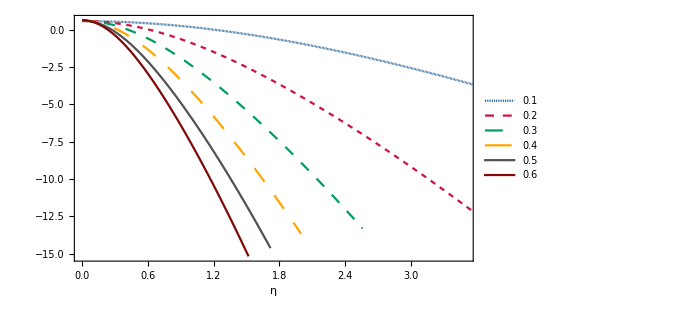

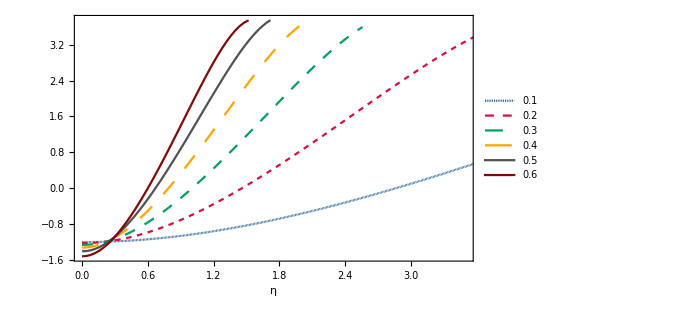

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.11,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameStyle->Directive[25,GrayLevel[0],FontFamily->"Times New Roman",AbsoluteThickness[2]],LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},PlotStyle->style,FrameLabel->{Style[HoldForm["η"],25],None},ImageSize->500,PlotRange->{{0,3.5},All},PlotLegends->
Placed[{Style[HoldForm["0.1"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.2"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.3"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.4"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.5"],FontSize-> 18,FontFamily->"Times New Roman"],Style[HoldForm["0.6"],FontSize-> 18,FontFamily->"Times New Roman"]},{0.88,0.3}],FrameTicksStyle->{Directive[25,Thick],Directive[25,Thick]}]
```

```mathematica
Max[Abs[(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100],Abs[(Max[Re[Tda[[2]]]]-Min[Re[Tda[[2]]]])/Min[Re[Tda[[2]]]]*100],Abs[(Max[Re[Tda[[3]]]]-Min[Re[Tda[[3]]]])/Min[Re[Tda[[3]]]]*100],Abs[(Max[Re[Tda[[4]]]]-Min[Re[Tda[[4]]]])/Min[Re[Tda[[4]]]]*100],Abs[(Max[Re[Tda[[5]]]]-Min[Re[Tda[[5]]]])/Min[Re[Tda[[5]]]]*100],Abs[(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100]]
Max[Abs[(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100],Abs[(Max[Im[Tda[[2]]]]-Min[Im[Tda[[2]]]])/Min[Im[Tda[[2]]]]*100],Abs[(Max[Im[Tda[[3]]]]-Min[Im[Tda[[3]]]])/Min[Im[Tda[[3]]]]*100],Abs[(Max[Im[Tda[[4]]]]-Min[Im[Tda[[4]]]])/Min[Im[Tda[[4]]]]*100],Abs[(Max[Im[Tda[[5]]]]-Min[Im[Tda[[5]]]])/Min[Im[Tda[[5]]]]*100],Abs[(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100]]
```

0.700182

0.325327

```mathematica
Max[Abs[(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100],Abs[(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100],Abs[(Max[Re[Tdp[[3]]]]-Min[Re[Tdp[[3]]]])/Min[Re[Tdp[[3]]]]*100],Abs[(Max[Re[Tdp[[4]]]]-Min[Re[Tdp[[4]]]])/Min[Re[Tdp[[4]]]]*100],Abs[(Max[Re[Tdp[[5]]]]-Min[Re[Tdp[[5]]]])/Min[Re[Tdp[[5]]]]*100],Abs[(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100],Abs[(Max[Im[Tdp[[2]]]]-Min[Im[Tdp[[2]]]])/Min[Im[Tdp[[2]]]]*100],Abs[(Max[Im[Tdp[[3]]]]-Min[Im[Tdp[[3]]]])/Min[Im[Tdp[[3]]]]*100],Abs[(Max[Im[Tdp[[4]]]]-Min[Im[Tdp[[4]]]])/Min[Im[Tdp[[4]]]]*100],Abs[(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100],Abs[(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100]]
```

17.8327

5.13551

### Isospectrality breaking m=+1 at=0.4

#### Axial modes

```mathematica
Ta={{{0.+0. ⅈ,0.27829464008301014-0.09080113348884336 ⅈ},{0.04+0.04 ⅈ,0.2782945896133177-0.09080110476385377 ⅈ},{0.08+0.08 ⅈ,0.2782944382043443-0.09080101858879758 ⅈ},{0.12+0.12 ⅈ,0.27829418585690624-0.09080087496369983 ⅈ},{0.16+0.16 ⅈ,0.27829383257228013-0.09080067388855413 ⅈ},{0.2+0.2 ⅈ,0.2782933783522534-0.09080041536335096 ⅈ},{0.24+0.24 ⅈ,0.27829282319912396-0.09080009938807716 ⅈ},{0.28+0.28 ⅈ,0.27829216711570054-0.09079972596271531 ⅈ},{0.32+0.32 ⅈ,0.278291410105303-0.09079929508724284 ⅈ},{0.36+0.36 ⅈ,0.2782905521717621-0.09079880676163106 ⅈ},{0.4+0.4 ⅈ,0.2782895933194193-0.09079826098584401 ⅈ},{0.44+0.44 ⅈ,0.2782885335531279-0.0907976577598372 ⅈ},{0.48+0.48 ⅈ,0.2782873728782521-0.09079699708355618 ⅈ},{0.52+0.52 ⅈ,0.2782861113006677-0.09079627895693484 ⅈ},{0.56+0.56 ⅈ,0.27828474882676213-0.09079550337989388 ⅈ},{0.6+0.6 ⅈ,0.2782832854634346-0.09079467035233862 ⅈ},{0.64+0.64 ⅈ,0.27828172121809647-0.09079377987415731 ⅈ},{0.68+0.68 ⅈ,0.278280056098671-0.09079283194521853 ⅈ},{0.72+0.72 ⅈ,0.278278290113594-0.09079182656536913 ⅈ},{0.76+0.76 ⅈ,0.2782764232718139-0.09079076373443155 ⅈ},{0.8+0.8 ⅈ,0.27827445558279157-0.09078964345220131 ⅈ},{0.84+0.84 ⅈ,0.27827238705650115-0.0907884657184439 ⅈ},{0.88+0.88 ⅈ,0.27827021770342997-0.09078723053289213 ⅈ},{0.92+0.92 ⅈ,0.2782679475345785-0.09078593789524281 ⅈ},{0.96+0.96 ⅈ,0.27826557656146117-0.09078458780515339 ⅈ},{1.+1. ⅈ,0.278263104796106-0.0907831802622387 ⅈ},{1.04+1.04 ⅈ,0.27826053225105535-0.09078171526606701 ⅈ},{1.08+1.08 ⅈ,0.2782578589393654-0.09078019281615708 ⅈ},{1.12+1.12 ⅈ,0.2782550848746073-0.09077861291197274 ⅈ},{1.16+1.16 ⅈ,0.27825221007086676-0.0907769755529203 ⅈ},{1.2+1.2 ⅈ,0.27824923454274425-0.0907752807383435 ⅈ},{1.24+1.24 ⅈ,0.2782461583053553-0.09077352846751921 ⅈ},{1.28+1.28 ⅈ,0.2782429813743309-0.09077171873965295 ⅈ},{1.32+1.32 ⅈ,0.2782397037658173-0.09076985155387411 ⅈ},{1.36+1.36 ⅈ,0.2782363254964765-0.09076792690923104 ⅈ},{1.4+1.4 ⅈ,0.27823284658348596-0.09076594480468583 ⅈ},{1.44+1.44 ⅈ,0.278229267044539-0.0907639052391094 ⅈ},{1.48+1.48 ⅈ,0.278225586897845-0.09076180821127572 ⅈ},{1.52+1.52 ⅈ,0.2782218061621291-0.0907596537198565 ⅈ},{1.56+1.56 ⅈ,0.2782179248566328-0.09075744176341535 ⅈ},{1.6+1.6 ⅈ,0.2782139430011133-0.09075517234040184 ⅈ},{1.64+1.64 ⅈ,0.2782098606158438-0.09075284544914541 ⅈ},{1.68+1.68 ⅈ,0.27820567772161353-0.09075046108784919 ⅈ},{1.72+1.72 ⅈ,0.27820139433972796-0.0907480192545835 ⅈ},{1.76+1.76 ⅈ,0.2781970104920076-0.09074551994727936 ⅈ},{1.8+1.8 ⅈ,0.27819252620078905-0.09074296316372152 ⅈ},{1.84+1.84 ⅈ,0.2781879414889242-0.09074034890154162 ⅈ},{1.88+1.88 ⅈ,0.2781832563797798-0.09073767715821114 ⅈ},{1.92+1.92 ⅈ,0.27817847089723763-0.0907349479310339 ⅈ},{1.96+1.96 ⅈ,0.27817358506569373-0.09073216121713878 ⅈ},{2.+2. ⅈ,0.2781685989100585-0.09072931701347196 ⅈ},{2.04+2.04 ⅈ,0.2781635124557553-0.09072641531678897 ⅈ},{2.08+2.08 ⅈ,0.278158325728721-0.0907234561236469 ⅈ},{2.12+2.12 ⅈ,0.2781530387554044-0.09072043943039605 ⅈ},{2.16+2.16 ⅈ,0.2781476515627663-0.0907173652331715 ⅈ},{2.2+2.2 ⅈ,0.27814216417827814-0.09071423352788467 ⅈ},{2.24+2.24 ⅈ,0.27813657662992175-0.0907110443102144 ⅈ},{2.28+2.28 ⅈ,0.2781308889461878-0.09070779757559819 ⅈ},{2.32+2.32 ⅈ,0.27812510115607536-0.0907044933192229 ⅈ},{2.36+2.36 ⅈ,0.27811921328909034-0.09070113153601561 ⅈ},{2.4+2.4 ⅈ,0.27811322537524463-0.09069771222063391 ⅈ},{2.44+2.44 ⅈ,0.2781071374450547-0.0906942353674563 ⅈ},{2.48+2.48 ⅈ,0.27810094952953995-0.09069070097057239 ⅈ},{2.52+2.52 ⅈ,0.2780946616602218-0.09068710902377265 ⅈ},{2.56+2.56 ⅈ,0.2780882738691214-0.09068345952053831 ⅈ},{2.6+2.6 ⅈ,0.2780817861887582-0.09067975245403077 ⅈ},{2.64+2.64 ⅈ,0.2780751986521483-0.09067598781708103 ⅈ},{2.68+2.68 ⅈ,0.2780685112928021-0.09067216560217874 ⅈ},{2.72+2.72 ⅈ,0.2780617241447223-0.09066828580146123 ⅈ},{2.76+2.76 ⅈ,0.2780548372424017-0.0906643484067023 ⅈ},{2.8+2.8 ⅈ,0.2780478506208209-0.09066035340930077 ⅈ},{2.84+2.84 ⅈ,0.2780407643154452-0.0906563008002687 ⅈ},{2.88+2.88 ⅈ,0.2780335783622228-0.0906521905702198 ⅈ},{2.92+2.92 ⅈ,0.27802629279758106-0.09064802270935718 ⅈ},{2.96+2.96 ⅈ,0.278018907658424-0.0906437972074613 ⅈ},{3.+3. ⅈ,0.27801142298212883-0.09063951405387749 ⅈ},{3.04+3.04 ⅈ,0.27800383880654284-0.09063517323750321 ⅈ},{3.08+3.08 ⅈ,0.27799615516997933-0.09063077474677544 ⅈ},{3.12+3.12 ⅈ,0.27798837211121447-0.09062631856965747 ⅈ},{3.16+3.16 ⅈ,0.2779804896694829-0.09062180469362577 ⅈ},{3.2+3.2 ⅈ,0.27797250788447375-0.09061723310565663 ⅈ},{3.24+3.24 ⅈ,0.2779644267963262-0.09061260379221239 ⅈ},{3.28+3.28 ⅈ,0.2779562464456249-0.09060791673922781 ⅈ},{3.32+3.32 ⅈ,0.2779479668733951-0.09060317193209587 ⅈ},{3.36+3.36 ⅈ,0.27793958812109776-0.09059836935565363 ⅈ},{3.4+3.4 ⅈ,0.2779311102306241-0.09059350899416792 ⅈ},{3.44+3.44 ⅈ,0.27792253324429006-0.09058859083132063 ⅈ},{3.48+3.48 ⅈ,0.27791385720483075-0.09058361485019387 ⅈ},{3.52+3.52 ⅈ,0.2779050821553941-0.09057858103325503 ⅈ},{3.56+3.56 ⅈ,0.2778962081395347-0.09057348936234165 ⅈ},{3.6+3.6 ⅈ,0.27788723520120695-0.09056833981864586 ⅈ},{3.64+3.64 ⅈ,0.2778781633847587-0.09056313238269897 ⅈ},{3.68+3.68 ⅈ,0.27786899273492344-0.09055786703435562 ⅈ},{3.72+3.72 ⅈ,0.27785972329681335-0.09055254375277784 ⅈ},{3.76+3.76 ⅈ,0.2778503551159111-0.0905471625164188 ⅈ},{3.8+3.8 ⅈ,0.27784088823806197-0.09054172330300658 ⅈ},{3.84+3.84 ⅈ,0.2778313227094652-0.0905362260895277 ⅈ},{3.88+3.88 ⅈ,0.2778216585766656-0.09053067085221024 ⅈ},{3.92+3.92 ⅈ,0.2778118958865437-0.09052505756650707 ⅈ},{3.96+3.96 ⅈ,0.2778020346863072-0.09051938620707876 ⅈ},{4.+4. ⅈ,0.27779207502348024-0.09051365674777632 ⅈ},{4.04+4.04 ⅈ,0.2777820169458936-0.09050786916162379 ⅈ},{4.08+4.08 ⅈ,0.27777186050167413-0.09050202342080069 ⅈ},{4.12+4.12 ⅈ,0.2777616057392334-0.09049611949662417 ⅈ},{4.16+4.16 ⅈ,0.2777512527072567-0.09049015735953128 ⅈ},{4.2+4.2 ⅈ,0.2777408014546907-0.09048413697906058 ⅈ},{4.24+4.24 ⅈ,0.2777302520307319-0.09047805832383427 ⅈ},{4.28+4.28 ⅈ,0.2777196044848127-0.09047192136153948 ⅈ},{4.32+4.32 ⅈ,0.27770885886658997-0.09046572605890991 ⅈ},{4.36+4.36 ⅈ,0.27769801522592963-0.09045947238170719 ⅈ},{4.4+4.4 ⅈ,0.27768707361289413-0.09045316029470185 ⅈ},{4.44+4.44 ⅈ,0.2776760340777264-0.09044678976165457 ⅈ},{4.48+4.48 ⅈ,0.27766489667083616-0.09044036074529702 ⅈ},{4.52+4.52 ⅈ,0.2776536614427836-0.09043387320731257 ⅈ},{4.56+4.56 ⅈ,0.2776423284442632-0.0904273271083171 ⅈ},{4.6+4.6 ⅈ,0.2776308977260876-0.09042072240783947 ⅈ},{4.64+4.64 ⅈ,0.2776193693391702-0.090414059064302 ⅈ},{4.68+4.68 ⅈ,0.2776077433345073-0.09040733703500091 ⅈ},{4.72+4.72 ⅈ,0.2775960197631601-0.09040055627608638 ⅈ},{4.76+4.76 ⅈ,0.2775841986762359-0.09039371674254298 ⅈ},{4.8+4.8 ⅈ,0.2775722801248682-0.09038681838816953 ⅈ},{4.84+4.84 ⅈ,0.27756026416019725-0.09037986116555936 ⅈ},{4.88+4.88 ⅈ,0.27754815083334916-0.09037284502608019 ⅈ},{4.92+4.92 ⅈ,0.2775359401954146-0.09036576991985396 ⅈ},{4.96+4.96 ⅈ,0.2775236322974268-0.09035863579573691 ⅈ},{5.+5. ⅈ,0.2775112271903394-0.09035144260129933 ⅈ},{5.04+5.04 ⅈ,0.27749872492500266-0.0903441902828053 ⅈ},{5.08+5.08 ⅈ,0.27748612555213986-0.09033687878519271 ⅈ},{5.12+5.12 ⅈ,0.27747342912232303-0.09032950805205296 ⅈ},{5.16+5.16 ⅈ,0.2774606356859469-0.09032207802561082 ⅈ},{5.2+5.2 ⅈ,0.2774477452932036-0.09031458864670427 ⅈ},{5.24+5.24 ⅈ,0.2774347579940554-0.09030703985476435 ⅈ},{5.28+5.28 ⅈ,0.2774216738382077-0.09029943158779526 ⅈ},{5.32+5.32 ⅈ,0.2774084928750804-0.09029176378235415 ⅈ},{5.36+5.36 ⅈ,0.27739521515377913-0.0902840363735314 ⅈ},{5.4+5.4 ⅈ,0.27738184072306515-0.0902762492949306 ⅈ},{5.44+5.44 ⅈ,0.27736836963132533-0.09026840247864894 ⅈ},{5.48+5.48 ⅈ,0.27735480192654005-0.0902604958552576 ⅈ},{5.52+5.52 ⅈ,0.2773411376562514-0.09025252935378221 ⅈ},{5.56+5.56 ⅈ,0.27732737686753023-0.09024450290168361 ⅈ},{5.6+5.6 ⅈ,0.2773135196069419-0.09023641642483864 ⅈ},{5.64+5.64 ⅈ,0.2772995659205116-0.09022826984752122 ⅈ},{5.68+5.68 ⅈ,0.27728551585368866-0.09022006309238349 ⅈ},{5.72+5.72 ⅈ,0.2772713694513104-0.09021179608043751 ⅈ},{5.76+5.76 ⅈ,0.27725712675756425-0.09020346873103682 ⅈ},{5.8+5.8 ⅈ,0.2772427878159492-0.09019508096185826 ⅈ},{5.84+5.84 ⅈ,0.2772283526692374-0.09018663268888455 ⅈ},{5.88+5.88 ⅈ,0.27721382135943295-0.09017812382638676 ⅈ},{5.92+5.92 ⅈ,0.27719919392773124-0.09016955428690702 ⅈ},{5.96+5.96 ⅈ,0.27718447041447675-0.09016092398124204 ⅈ},{6.+6. ⅈ,0.2771696508591198-0.09015223281842663 ⅈ},{6.04+6.04 ⅈ,0.27715473530017243-0.09014348070571765 ⅈ},{6.08+6.08 ⅈ,0.2771397237751635-0.0901346675485786 ⅈ},{6.12+6.12 ⅈ,0.2771246163205923-0.09012579325066453 ⅈ},{6.16+6.16 ⅈ,0.27710941297188163-0.09011685771380724 ⅈ},{6.2+6.2 ⅈ,0.27709411376332943-0.09010786083800147 ⅈ},{6.24+6.24 ⅈ,0.27707871872805967-0.09009880252139106 ⅈ},{6.28+6.28 ⅈ,0.27706322789797183-0.09008968266025606 ⅈ},{6.32+6.32 ⅈ,0.2770476413036898-0.09008050114900035 ⅈ},{6.36+6.36 ⅈ,0.2770319589745098-0.09007125788013971 ⅈ},{6.4+6.4 ⅈ,0.2770161809383457-0.0900619527442909 ⅈ},{6.44+6.44 ⅈ,0.27700030722167596-0.09005258563016094 ⅈ},{6.48+6.48 ⅈ,0.2769843378494867-0.09004315642453761 ⅈ},{6.52+6.52 ⅈ,0.27696827284521547-0.09003366501228036 ⅈ},{6.56+6.56 ⅈ,0.27695211223069344-0.09002411127631209 ⅈ},{6.6+6.6 ⅈ,0.276935856026086-0.09001449509761192 ⅈ},{6.64+6.64 ⅈ,0.27691950424983286-0.09000481635520848 ⅈ},{6.68+6.68 ⅈ,0.2769030569185868-0.08999507492617455 ⅈ},{6.72+6.72 ⅈ,0.2768865140471509-0.08998527068562218 ⅈ},{6.76+6.76 ⅈ,0.27686987564841575-0.0899754035066991 ⅈ},{6.8+6.8 ⅈ,0.27685314173329395-0.08996547326058602 ⅈ},{6.84+6.84 ⅈ,0.27683631231065464-0.08995547981649499 ⅈ},{6.88+6.88 ⅈ,0.2768193873872568-0.08994542304166891 ⅈ},{6.92+6.92 ⅈ,0.2768023669676808-0.08993530280138214 ⅈ},{6.96+6.96 ⅈ,0.27678525105425905-0.08992511895894223 ⅈ},{7.+7. ⅈ,0.2767680396470063-0.08991487137569303 ⅈ},{7.04+7.04 ⅈ,0.2767507327435474-0.08990455991101896 ⅈ},{7.08+7.08 ⅈ,0.2767333303390449-0.08989418442235067 ⅈ},{7.12+7.12 ⅈ,0.2767158324261258-0.08988374476517189 ⅈ}},{{0.+0. ⅈ,0.280219729636685-0.0909599304122132 ⅈ},{0.04+0.04 ⅈ,0.28021952764648334-0.09095980982758797 ⅈ},{0.08+0.08 ⅈ,0.2802189216780767-0.09095944807254942 ⅈ},{0.12+0.12 ⅈ,0.28021791174008-0.09095884514481062 ⅈ},{0.16+0.16 ⅈ,0.2802164978465151-0.09095800104034461 ⅈ},{0.2+0.2 ⅈ,0.28021468001701233-0.09095691575348364 ⅈ},{0.24+0.24 ⅈ,0.28021245827681107-0.09095558927688877 ⅈ},{0.28+0.28 ⅈ,0.28020983265675925-0.09095402160151121 ⅈ},{0.32+0.32 ⅈ,0.28020680319331354-0.09095221271654473 ⅈ},{0.36+0.36 ⅈ,0.28020336992853867-0.09095016260936954 ⅈ},{0.4+0.4 ⅈ,0.2801995329101067-0.0909478712654871 ⅈ},{0.44+0.44 ⅈ,0.280195292191296-0.09094533866844651 ⅈ},{0.48+0.48 ⅈ,0.28019064783098946-0.0909425647997618 ⅈ},{0.52+0.52 ⅈ,0.28018559989367203-0.09093954963882031 ⅈ},{0.56+0.56 ⅈ,0.2801801484494276-0.09093629316278219 ⅈ},{0.6+0.6 ⅈ,0.2801742935739346-0.09093279534647086 ⅈ},{0.64+0.64 ⅈ,0.28016803534846046-0.09092905616225433 ⅈ},{0.68+0.68 ⅈ,0.28016137385985496-0.09092507557991707 ⅈ},{0.72+0.72 ⅈ,0.28015430920054146-0.09092085356652328 ⅈ},{0.76+0.76 ⅈ,0.2801468414685066-0.09091639008626995 ⅈ},{0.8+0.8 ⅈ,0.2801389707672878-0.09091168510033118 ⅈ},{0.84+0.84 ⅈ,0.28013069720595796-0.09090673856669258 ⅈ},{0.88+0.88 ⅈ,0.2801220208991086-0.09090155043997628 ⅈ},{0.92+0.92 ⅈ,0.2801129419668282-0.09089612067125587 ⅈ},{0.96+0.96 ⅈ,0.28010346053467894-0.09089044920786203 ⅈ},{1.+1. ⅈ,0.28009357673366864-0.09088453599317779 ⅈ},{1.04+1.04 ⅈ,0.2800832907002192-0.090878380966424 ⅈ},{1.08+1.08 ⅈ,0.2800726025761301-0.0908719840624348 ⅈ},{1.12+1.12 ⅈ,0.2800615125085373-0.09086534521142252 ⅈ},{1.16+1.16 ⅈ,0.28005002064986684-0.09085846433873274 ⅈ},{1.2+1.2 ⅈ,0.28003812715778276-0.09085134136458868 ⅈ},{1.24+1.24 ⅈ,0.28002583219512805-0.09084397620382506 ⅈ},{1.28+1.28 ⅈ,0.2800131359298597-0.09083636876561178 ⅈ},{1.32+1.32 ⅈ,0.2800000385349762-0.09082851895316649 ⅈ},{1.36+1.36 ⅈ,0.27998654018843633-0.09082042666345695 ⅈ},{1.4+1.4 ⅈ,0.2799726410730707-0.09081209178689223 ⅈ},{1.44+1.44 ⅈ,0.27995834137648357-0.09080351420700328 ⅈ},{1.48+1.48 ⅈ,0.2799436412909448-0.09079469380011265 ⅈ},{1.52+1.52 ⅈ,0.2799285410132716-0.09078563043499344 ⅈ},{1.56+1.56 ⅈ,0.27991304074469914-0.09077632397251705 ⅈ},{1.6+1.6 ⅈ,0.27989714069073945-0.09076677426529031 ⅈ},{1.64+1.64 ⅈ,0.27988084106102734-0.09075698115728173 ⅈ},{1.68+1.68 ⅈ,0.27986414206915344-0.09074694448343669 ⅈ},{1.72+1.72 ⅈ,0.27984704393248244-0.0907366640692821 ⅈ},{1.76+1.76 ⅈ,0.27982954687195655-0.09072613973052017 ⅈ},{1.8+1.8 ⅈ,0.2798116511118832-0.09071537127261171 ⅈ},{1.84+1.84 ⅈ,0.27979335687970547-0.09070435849034893 ⅈ},{1.88+1.88 ⅈ,0.27977466440575455-0.09069310116741774 ⅈ},{1.92+1.92 ⅈ,0.2797555739229839-0.09068159907595039 ⅈ},{1.96+1.96 ⅈ,0.279736085666683-0.09066985197606765 ⅈ},{2.+2. ⅈ,0.27971619987417073-0.09065785961541192 ⅈ},{2.04+2.04 ⅈ,0.27969591678446587-0.09064562172867044 ⅈ},{2.08+2.08 ⅈ,0.2796752366379352-0.09063313803709017 ⅈ},{2.12+2.12 ⅈ,0.2796541596759169-0.09062040824798354 ⅈ},{2.16+2.16 ⅈ,0.27963268614031855-0.09060743205422639 ⅈ},{2.2+2.2 ⅈ,0.2796108162731883-0.0905942091337483 ⅈ},{2.24+2.24 ⅈ,0.279588550316258-0.09058073914901539 ⅈ},{2.28+2.28 ⅈ,0.279565888510457-0.09056702174650758 ⅈ},{2.32+2.32 ⅈ,0.2795428310953952-0.09055305655618899 ⅈ},{2.36+2.36 ⅈ,0.27951937830881396-0.09053884319097419 ⅈ},{2.4+2.4 ⅈ,0.2794955303860044-0.0905243812461898 ⅈ},{2.44+2.44 ⅈ,0.27947128755918915-0.09050967029903308 ⅈ},{2.48+2.48 ⅈ,0.27944665005686975-0.09049470990802785 ⅈ},{2.52+2.52 ⅈ,0.27942161810313443-0.09047949961247977 ⅈ},{2.56+2.56 ⅈ,0.2793961919169283-0.09046403893193103 ⅈ},{2.6+2.6 ⅈ,0.27937037171128093-0.09044832736561657 ⅈ},{2.64+2.64 ⅈ,0.27934415769249354-0.09043236439192295 ⅈ},{2.68+2.68 ⅈ,0.2793175500592802-0.09041614946785102 ⅈ},{2.72+2.72 ⅈ,0.2792905490018658-0.09039968202848472 ⅈ},{2.76+2.76 ⅈ,0.27926315470103424-0.09038296148646685 ⅈ},{2.8+2.8 ⅈ,0.27923536732713133-0.09036598723148442 ⅈ},{2.84+2.84 ⅈ,0.27920718703901454-0.09034875862976503 ⅈ},{2.88+2.88 ⅈ,0.27917861398295285-0.09033127502358697 ⅈ},{2.92+2.92 ⅈ,0.2791496482914727-0.09031353573080432 ⅈ},{2.96+2.96 ⅈ,0.27912029008214895-0.09029554004439078 ⅈ},{3.+3. ⅈ,0.2790905394563405-0.09027728723200379 ⅈ},{3.04+3.04 ⅈ,0.2790603964978673-0.09025877653557193 ⅈ},{3.08+3.08 ⅈ,0.2790298612716286-0.09024000717090869 ⅈ},{3.12+3.12 ⅈ,0.27899893382216134-0.09022097832735573 ⅈ},{3.16+3.16 ⅈ,0.27896761417213567-0.09020168916745852 ⅈ},{3.2+3.2 ⅈ,0.278935902320789-0.09018213882667811 ⅈ},{3.24+3.24 ⅈ,0.27890379824229516-0.09016232641314266 ⅈ},{3.28+3.28 ⅈ,0.27887130188406906-0.09014225100744246 ⅈ},{3.32+3.32 ⅈ,0.27883841316500557-0.09012191166247258 ⅈ},{3.36+3.36 ⅈ,0.2788051319736514-0.09010130740332704 ⅈ},{3.4+3.4 ⅈ,0.278771458166311-0.09008043722724983 ⅈ},{3.44+3.44 ⅈ,0.2787373915650834-0.09005930010364614 ⅈ},{3.48+3.48 ⅈ,0.278702931955833-0.09003789497416007 ⅈ},{3.52+3.52 ⅈ,0.27866807908609165-0.09001622075282262 ⅈ},{3.56+3.56 ⅈ,0.27863283266289285-0.08999427632627621 ⅈ},{3.6+3.6 ⅈ,0.2785971923505405-0.08997206055408084 ⅈ},{3.64+3.64 ⅈ,0.2785611577683093-0.0899495722691075 ⅈ}},{{0.+0. ⅈ,0.28341650078845715-0.09122980332415005 ⅈ},{0.04+0.04 ⅈ,0.28341604587384356-0.09122951147536512 ⅈ},{0.08+0.08 ⅈ,0.28341468113268603-0.09122863591761372 ⅈ},{0.12+0.12 ⅈ,0.2834124065775749-0.09122717661958464 ⅈ},{0.16+0.16 ⅈ,0.28340922222870923-0.09122513352847253 ⅈ},{0.2+0.2 ⅈ,0.2834051281143109-0.09122250657006968 ⅈ},{0.24+0.24 ⅈ,0.28340012427056666-0.09121929564848479 ⅈ},{0.28+0.28 ⅈ,0.2833942107415508-0.09121550064578146 ⅈ},{0.32+0.32 ⅈ,0.28338738757912857-0.09121112142153498 ⅈ},{0.36+0.36 ⅈ,0.28337965484283717-0.09120615781230702 ⅈ},{0.4+0.4 ⅈ,0.28337101259974246-0.09120060963103815 ⅈ},{0.44+0.44 ⅈ,0.2833614609242686-0.09119447666635647 ⅈ},{0.48+0.48 ⅈ,0.28335099989799883-0.09118775868180233 ⅈ},{0.52+0.52 ⅈ,0.2833396296094416-0.09118045541496807 ⅈ},{0.56+0.56 ⅈ,0.28332735015376154-0.09117256657655133 ⅈ},{0.6+0.6 ⅈ,0.2833141616324676-0.0911640918493218 ⅈ},{0.64+0.64 ⅈ,0.28330006415305714-0.09115503088699976 ⅈ},{0.68+0.68 ⅈ,0.2832850578286082-0.09114538331304582 ⅈ},{0.72+0.72 ⅈ,0.28326914277731613-0.09113514871936033 ⅈ},{0.76+0.76 ⅈ,0.2832523191219681-0.09112432666489256 ⅈ},{0.8+0.8 ⅈ,0.2832345869893489-0.09111291667415757 ⅈ},{0.84+0.84 ⅈ,0.28321594650957105-0.09110091823566076 ⅈ},{0.88+0.88 ⅈ,0.28319639781532224-0.09108833080022939 ⅈ},{0.92+0.92 ⅈ,0.28317594104102123-0.09107515377925023 ⅈ},{0.96+0.96 ⅈ,0.2831545763218742-0.0910613865428134 ⅈ},{1.+1. ⅈ,0.28313230379282234-0.09104702841776208 ⅈ},{1.04+1.04 ⅈ,0.28310912358736984-0.09103207868564854 ⅈ},{1.08+1.08 ⅈ,0.28308503583628336-0.09101653658059705 ⅈ},{1.12+1.12 ⅈ,0.28306004066615054-0.09100040128707382 ⅈ},{1.16+1.16 ⅈ,0.28303413819778617-0.09098367193756687 ⅈ},{1.2+1.2 ⅈ,0.2830073285444737-0.09096634761017651 ⅈ},{1.24+1.24 ⅈ,0.28297961181002795-0.09094842732611885 ⅈ},{1.28+1.28 ⅈ,0.2829509880866672-0.09092991004714662 ⅈ},{1.32+1.32 ⅈ,0.2829214574526763-0.09091079467288951 ⅈ},{1.36+1.36 ⅈ,0.28289101996984894-0.09089108003812028 ⅈ},{1.4+1.4 ⅈ,0.2828596756806912-0.09087076490995113 ⅈ},{1.44+1.44 ⅈ,0.28282742460536897-0.09084984798496763 ⅈ},{1.48+1.48 ⅈ,0.2827942667383818-0.09082832788630728 ⅈ},{1.52+1.52 ⅈ,0.2827602020449462-0.09080620316069252 ⅈ},{1.56+1.56 ⅈ,0.2827252304570661-0.0907834722754281 ⅈ},{1.6+1.6 ⅈ,0.28268935186927396-0.09076013361537469 ⅈ},{1.64+1.64 ⅈ,0.28265256613401873-0.09073618547991236 ⅈ},{1.68+1.68 ⅈ,0.2826148730566827-0.09071162607990985 ⅈ},{1.72+1.72 ⅈ,0.28257627239020205-0.09068645353471572 ⅈ},{1.76+1.76 ⅈ,0.2825367638292722-0.09066066586919251 ⅈ},{1.8+1.8 ⅈ,0.2824963470041131-0.09063426101081472 ⅈ},{1.84+1.84 ⅈ,0.2824550214737722-0.09060723678685453 ⅈ},{1.88+1.88 ⅈ,0.2824127867189431-0.09057959092168413 ⅈ},{1.92+1.92 ⅈ,0.2823696421342751-0.09055132103422264 ⅈ},{1.96+1.96 ⅈ,0.2823255870201528-0.09052242463556177 ⅈ},{2.+2. ⅈ,0.2822806205739215-0.09049289912680633 ⅈ},{2.04+2.04 ⅈ,0.28223474188053904-0.0904627417971699 ⅈ},{2.08+2.08 ⅈ,0.2821879499026306-0.09043194982236827 ⅈ},{2.12+2.12 ⅈ,0.28214024346992933-0.09040052026335992 ⅈ},{2.16+2.16 ⅈ,0.2820916212680832-0.09036845006548348 ⅈ},{2.2+2.2 ⅈ,0.2820420818268134-0.09033573605805001 ⅈ},{2.24+2.24 ⅈ,0.2819916235074091-0.09030237495444875 ⅈ},{2.28+2.28 ⅈ,0.28194024448955-0.0902683633528342 ⅈ},{2.32+2.32 ⅈ,0.28188794275744744-0.09023369773746184 ⅈ},{2.36+2.36 ⅈ,0.2818347160853024-0.09019837448074979 ⅈ},{2.4+2.4 ⅈ,0.2817805620220807-0.09016238984614486 ⅈ},{2.44+2.44 ⅈ,0.28172547787561275-0.09012573999187894 ⅈ},{2.48+2.48 ⅈ,0.2816694606960319-0.09008842097570564 ⅈ},{2.52+2.52 ⅈ,0.28161250725856857-0.09005042876071083 ⅈ},{2.56+2.56 ⅈ,0.28155461404573096-0.09001175922229802 ⅈ}},{{0.+0. ⅈ,0.28786855352426727-0.09161806454120275 ⅈ},{0.04+0.04 ⅈ,0.28786774356896466-0.09161749737159099 ⅈ},{0.08+0.08 ⅈ,0.28786531367253093-0.091615795800137 ⅈ},{0.12+0.12 ⅈ,0.28786126375138377-0.09161295964449123 ⅈ},{0.16+0.16 ⅈ,0.28785559366452274-0.09160898859924034 ⅈ},{0.2+0.2 ⅈ,0.2878483032138139-0.09160388223564615 ⅈ},{0.24+0.24 ⅈ,0.28783939214324394-0.09159764000048377 ⅈ},{0.28+0.28 ⅈ,0.2878288601379438-0.09159026121454511 ⅈ},{0.32+0.32 ⅈ,0.287816706822967-0.09158174507080594 ⅈ},{0.36+0.36 ⅈ,0.2878029317618082-0.09157209063225384 ⅈ},{0.4+0.4 ⅈ,0.28778753445463934-0.09156129682937514 ⅈ},{0.44+0.44 ⅈ,0.28777051433624234-0.09154936245729824 ⅈ},{0.48+0.48 ⅈ,0.28775187077361025-0.09153628617259103 ⅈ},{0.52+0.52 ⅈ,0.2877316030631865-0.09152206648971081 ⅈ},{0.56+0.56 ⅈ,0.28770971042770876-0.09150670177710492 ⅈ},{0.6+0.6 ⅈ,0.28768619201261764-0.09149019025296183 ⅈ},{0.64+0.64 ⅈ,0.287661046881989-0.0914725299806133 ⅈ},{0.68+0.68 ⅈ,0.28763427401394287-0.09145371886358894 ⅈ},{0.72+0.72 ⅈ,0.2876058722954767-0.09143375464032764 ⅈ},{0.76+0.76 ⅈ,0.2875758405166676-0.09141263487855127 ⅈ},{0.8+0.8 ⅈ,0.28754417736418236-0.09139035696930939 ⅈ},{0.84+0.84 ⅈ,0.28751088141402725-0.09136691812070685 ⅈ},{0.88+0.88 ⅈ,0.287475951123469-0.09134231535133004 ⅈ},{0.92+0.92 ⅈ,0.2874393848220456-0.09131654548339194 ⅈ},{0.96+0.96 ⅈ,0.28740118070158766-0.0912896051356213 ⅈ},{1.+1. ⅈ,0.2873613368051572-0.09126149071592807 ⅈ},{1.04+1.04 ⅈ,0.2873198510148135-0.09123219841388286 ⅈ},{1.08+1.08 ⅈ,0.2872767210381-0.0912017241930599 ⅈ},{1.12+1.12 ⅈ,0.2872319443931513-0.09117006378329404 ⅈ},{1.16+1.16 ⅈ,0.2871855183922994-0.09113721267292618 ⅈ},{1.2+1.2 ⅈ,0.28713744012406905-0.09110316610110933 ⅈ},{1.24+1.24 ⅈ,0.28708770643343273-0.09106791905027022 ⅈ},{1.28+1.28 ⅈ,0.28703631390019785-0.09103146623883333 ⅈ},{1.32+1.32 ⅈ,0.28698325881539555-0.090993802114331 ⅈ},{1.36+1.36 ⅈ,0.2869285371555312-0.09095492084704206 ⅈ},{1.4+1.4 ⅈ,0.2868721445545613-0.09091481632432372 ⅈ},{1.44+1.44 ⅈ,0.28681407627345584-0.09087348214582078 ⅈ},{1.48+1.48 ⅈ,0.28675432716720856-0.0908309116197668 ⅈ},{1.52+1.52 ⅈ,0.28669289164915923-0.09078709776061276 ⅈ},{1.56+1.56 ⅈ,0.2866297636524983-0.09074203328825516 ⅈ},{1.6+1.6 ⅈ,0.28656493658883375-0.09069571062916278 ⅈ},{1.64+1.64 ⅈ,0.28649840330370724-0.0906481219197387 ⅈ},{1.68+1.68 ⅈ,0.28643015602897176-0.0905992590122906 ⅈ},{1.72+1.72 ⅈ,0.28636018633195404-0.09054911348402056 ⅈ},{1.76+1.76 ⅈ,0.2862884850613577-0.09049767664948924 ⅈ},{1.8+1.8 ⅈ,0.2862150422898959-0.09044493957704854 ⅈ},{1.84+1.84 ⅈ,0.2861398472536779-0.09039089310978342 ⅈ},{1.88+1.88 ⅈ,0.28606288828842724-0.09033552789154685 ⅈ},{1.92+1.92 ⅈ,0.28598415276266376-0.0902788343987161 ⅈ},{1.96+1.96 ⅈ,0.2859036270080482-0.09022080297834031 ⅈ},{2.+2. ⅈ,0.2858212962471685-0.09016142389338982 ⅈ}},{{0.+0. ⅈ,0.2935551387058252-0.09213403543058969 ⅈ},{0.04+0.04 ⅈ,0.2935538701548203-0.09213305905686196 ⅈ},{0.08+0.08 ⅈ,0.29355006431605996-0.0921301297014526 ⅈ},{0.12+0.12 ⅈ,0.2935437206443447-0.09212524667104371 ⅈ},{0.16+0.16 ⅈ,0.2935348382267276-0.09211840880713526 ⅈ},{0.2+0.2 ⅈ,0.293523415780504-0.09210961448500857 ⅈ},{0.24+0.24 ⅈ,0.2935094516485692-0.09209886161091162 ⅈ},{0.28+0.28 ⅈ,0.2934929437933534-0.09208614761844679 ⅈ},{0.32+0.32 ⅈ,0.29347388978926764-0.092071469464167 ⅈ},{0.36+0.36 ⅈ,0.29345228681356844-0.09205482362238943 ⅈ},{0.4+0.4 ⅈ,0.2934281316355383-0.09203620607923955 ⅈ},{0.44+0.44 ⅈ,0.2934014206038572-0.09201561232594367 ⅈ},{0.48+0.48 ⅈ,0.29337214963202174-0.09199303735139384 ⅈ},{0.52+0.52 ⅈ,0.2933403141816507-0.0919684756340177 ⅈ},{0.56+0.56 ⅈ,0.29330590924349126-0.09194192113299582 ⅈ},{0.6+0.6 ⅈ,0.2932689293159215-0.0919133672788812 ⅈ},{0.64+0.64 ⅈ,0.29322936838071995-0.09188280696369053 ⅈ},{0.68+0.68 ⅈ,0.29318721987584967-0.091850232530556 ⅈ},{0.72+0.72 ⅈ,0.29314247666497945-0.09181563576304722 ⅈ},{0.76+0.76 ⅈ,0.29309513100343826-0.09177900787429885 ⅈ},{0.8+0.8 ⅈ,0.29304517450027495-0.0917403394961112 ⅈ},{0.84+0.84 ⅈ,0.29299259807606404-0.09169962066822593 ⅈ},{0.88+0.88 ⅈ,0.29293739191607804-0.09165684082802142 ⅈ},{0.92+0.92 ⅈ,0.2928795454184133-0.09161198880092271 ⅈ},{0.96+0.96 ⅈ,0.29281904713663703-0.09156505279187396 ⅈ},{1.+1. ⅈ,0.29275588471649566-0.09151602037829239 ⅈ},{1.04+1.04 ⅈ,0.29269004482620953-0.09146487850499094 ⅈ},{1.08+1.08 ⅈ,0.2926215130798418-0.09141161348164968 ⅈ},{1.12+1.12 ⅈ,0.29255027395327804-0.09135621098349984 ⅈ},{1.16+1.16 ⅈ,0.2924763106922382-0.09129865605601532 ⅈ},{1.2+1.2 ⅈ,0.2923996052118828-0.09123893312450411 ⅈ},{1.24+1.24 ⅈ,0.2923201379874869-0.091177026009646 ⅈ},{1.28+1.28 ⅈ,0.29223788793574285-0.0911129179501699 ⅈ},{1.32+1.32 ⅈ,0.29215283228628736-0.09104659163402694 ⅈ},{1.36+1.36 ⅈ,0.29206494644312714-0.09097802923960072 ⅈ},{1.4+1.4 ⅈ,0.29197420383574496-0.09090721248869248 ⅈ},{1.44+1.44 ⅈ,0.2918805757597774-0.090834122713234 ⅈ},{1.48+1.48 ⅈ,0.2917840312074033-0.0907587409378667 ⅈ},{1.52+1.52 ⅈ,0.29168453668769206-0.0906810479808206 ⅈ},{1.56+1.56 ⅈ,0.2915820560375439-0.09060102457568546 ⅈ},{1.6+1.6 ⅈ,0.2914765502241294-0.09051865151693626 ⅈ},{1.64+1.64 ⅈ,0.2913679771401605-0.09043390983227467 ⅈ},{1.68+1.68 ⅈ,0.2912562913938106-0.09034678098503837 ⅈ},{1.72+1.72 ⅈ,0.2911414440956619-0.09025724711008189 ⅈ}},{{0.+0. ⅈ,0.30045310295282823-0.09278832509844867 ⅈ},{0.04+0.04 ⅈ,0.3004512693118783-0.09278677426482322 ⅈ},{0.08+0.08 ⅈ,0.30044576776003856-0.0927821210846875 ⅈ},{0.12+0.12 ⅈ,0.3004365964259674-0.09277436353517243 ⅈ},{0.16+0.16 ⅈ,0.30042375217865597-0.09276349824025859 ⅈ},{0.2+0.2 ⅈ,0.30040723061558083-0.09274952046938002 ⅈ},{0.24+0.24 ⅈ,0.30038702604334605-0.0927324241333665 ⅈ},{0.28+0.28 ⅈ,0.30036313145243465-0.09271220177934512 ⅈ},{0.32+0.32 ⅈ,0.3003355384858005-0.09268884458469924 ⅈ},{0.36+0.36 ⅈ,0.3003042374009631-0.09266234235021208 ⅈ},{0.4+0.4 ⅈ,0.3002692170251998-0.09263268349255774 ⅈ},{0.44+0.44 ⅈ,0.3002304647033638-0.09259985503634656 ⅈ},{0.48+0.48 ⅈ,0.3001879662377809-0.09256384260598151 ⅈ},{0.52+0.52 ⅈ,0.30014170581960237-0.09252463041764454 ⅈ},{0.56+0.56 ⅈ,0.3000916659509131-0.09248220127180422 ⅈ},{0.6+0.6 ⅈ,0.3000378273568139-0.0924365365467244 ⅈ},{0.64+0.64 ⅈ,0.29998016888661083-0.09238761619355695 ⅈ},{0.68+0.68 ⅈ,0.299918667403163-0.09233541873372397 ⅈ},{0.72+0.72 ⅈ,0.29985329765935287-0.09227992125944373 ⅈ},{0.76+0.76 ⅈ,0.2997840321605619-0.09222109943842194 ⅈ},{0.8+0.8 ⅈ,0.2997108410119576-0.09215892752393463 ⅈ},{0.84+0.84 ⅈ,0.2996336917493241-0.09209337837176318 ⅈ},{0.88+0.88 ⅈ,0.2995525491521139-0.09202442346571268 ⅈ},{0.92+0.92 ⅈ,0.29946737503736054-0.09195203295376426 ⅈ},{0.96+0.96 ⅈ,0.2993781280330543-0.09187617569728314 ⅈ},{1.+1. ⅈ,0.29928476332966525-0.09179681933608778 ⅈ},{1.04+1.04 ⅈ,0.2991872324084631-0.09171393037271809 ⅈ},{1.08+1.08 ⅈ,0.29908548274550223-0.09162747427971552 ⅈ},{1.12+1.12 ⅈ,0.29897945749028265-0.09153741563436213 ⅈ},{1.16+1.16 ⅈ,0.29886909511841486-0.09144371828597682 ⅈ},{1.2+1.2 ⅈ,0.29875432905802196-0.09134634556159513 ⅈ},{1.24+1.24 ⅈ,0.29863508729018207-0.0912452605166417 ⅈ},{1.28+1.28 ⅈ,0.29851129192445014-0.09114042623803578 ⅈ},{1.32+1.32 ⅈ,0.298382858751459-0.09103180620802932 ⅈ},{1.36+1.36 ⅈ,0.2982496967758146-0.09091936473793863 ⅈ},{1.4+1.4 ⅈ,0.2981117077340143-0.09080306748175672 ⅈ},{1.44+1.44 ⅈ,0.29796878560397727-0.09068288204036727 ⅈ},{1.48+1.48 ⅈ,0.2978208161150243-0.09055877866765598 ⅈ},{1.52+1.52 ⅈ,0.297667676269822-0.0904307310901304 ⅈ}}};
```

```mathematica
Tda={{{0.27829464008301014-0.09080113348884336 ⅈ},{0.2782945896133177-0.09080110476385377 ⅈ},{0.2782944382043443-0.09080101858879758 ⅈ},{0.27829418585690624-0.09080087496369983 ⅈ},{0.27829383257228013-0.09080067388855413 ⅈ},{0.2782933783522534-0.09080041536335096 ⅈ},{0.27829282319912396-0.09080009938807716 ⅈ},{0.27829216711570054-0.09079972596271531 ⅈ},{0.278291410105303-0.09079929508724284 ⅈ},{0.2782905521717621-0.09079880676163106 ⅈ},{0.2782895933194193-0.09079826098584401 ⅈ},{0.2782885335531279-0.0907976577598372 ⅈ},{0.2782873728782521-0.09079699708355618 ⅈ},{0.2782861113006677-0.09079627895693484 ⅈ},{0.27828474882676213-0.09079550337989388 ⅈ},{0.2782832854634346-0.09079467035233862 ⅈ},{0.27828172121809647-0.09079377987415731 ⅈ},{0.278280056098671-0.09079283194521853 ⅈ},{0.278278290113594-0.09079182656536913 ⅈ},{0.2782764232718139-0.09079076373443155 ⅈ},{0.27827445558279157-0.09078964345220131 ⅈ},{0.27827238705650115-0.0907884657184439 ⅈ},{0.27827021770342997-0.09078723053289213 ⅈ},{0.2782679475345785-0.09078593789524281 ⅈ},{0.27826557656146117-0.09078458780515339 ⅈ},{0.278263104796106-0.0907831802622387 ⅈ},{0.27826053225105535-0.09078171526606701 ⅈ},{0.2782578589393654-0.09078019281615708 ⅈ},{0.2782550848746073-0.09077861291197274 ⅈ},{0.27825221007086676-0.0907769755529203 ⅈ},{0.27824923454274425-0.0907752807383435 ⅈ},{0.2782461583053553-0.09077352846751921 ⅈ},{0.2782429813743309-0.09077171873965295 ⅈ},{0.2782397037658173-0.09076985155387411 ⅈ},{0.2782363254964765-0.09076792690923104 ⅈ},{0.27823284658348596-0.09076594480468583 ⅈ},{0.278229267044539-0.0907639052391094 ⅈ},{0.278225586897845-0.09076180821127572 ⅈ},{0.2782218061621291-0.0907596537198565 ⅈ},{0.2782179248566328-0.09075744176341535 ⅈ},{0.2782139430011133-0.09075517234040184 ⅈ},{0.2782098606158438-0.09075284544914541 ⅈ},{0.27820567772161353-0.09075046108784919 ⅈ},{0.27820139433972796-0.0907480192545835 ⅈ},{0.2781970104920076-0.09074551994727936 ⅈ},{0.27819252620078905-0.09074296316372152 ⅈ},{0.2781879414889242-0.09074034890154162 ⅈ},{0.2781832563797798-0.09073767715821114 ⅈ},{0.27817847089723763-0.0907349479310339 ⅈ},{0.27817358506569373-0.09073216121713878 ⅈ},{0.2781685989100585-0.09072931701347196 ⅈ},{0.2781635124557553-0.09072641531678897 ⅈ},{0.278158325728721-0.0907234561236469 ⅈ},{0.2781530387554044-0.09072043943039605 ⅈ},{0.2781476515627663-0.0907173652331715 ⅈ},{0.27814216417827814-0.09071423352788467 ⅈ},{0.27813657662992175-0.0907110443102144 ⅈ},{0.2781308889461878-0.09070779757559819 ⅈ},{0.27812510115607536-0.0907044933192229 ⅈ},{0.27811921328909034-0.09070113153601561 ⅈ},{0.27811322537524463-0.09069771222063391 ⅈ},{0.2781071374450547-0.0906942353674563 ⅈ},{0.27810094952953995-0.09069070097057239 ⅈ},{0.2780946616602218-0.09068710902377265 ⅈ},{0.2780882738691214-0.09068345952053831 ⅈ},{0.2780817861887582-0.09067975245403077 ⅈ},{0.2780751986521483-0.09067598781708103 ⅈ},{0.2780685112928021-0.09067216560217874 ⅈ},{0.2780617241447223-0.09066828580146123 ⅈ},{0.2780548372424017-0.0906643484067023 ⅈ},{0.2780478506208209-0.09066035340930077 ⅈ},{0.2780407643154452-0.0906563008002687 ⅈ},{0.2780335783622228-0.0906521905702198 ⅈ},{0.27802629279758106-0.09064802270935718 ⅈ},{0.278018907658424-0.0906437972074613 ⅈ},{0.27801142298212883-0.09063951405387749 ⅈ},{0.27800383880654284-0.09063517323750321 ⅈ},{0.27799615516997933-0.09063077474677544 ⅈ},{0.27798837211121447-0.09062631856965747 ⅈ},{0.2779804896694829-0.09062180469362577 ⅈ},{0.27797250788447375-0.09061723310565663 ⅈ},{0.2779644267963262-0.09061260379221239 ⅈ},{0.2779562464456249-0.09060791673922781 ⅈ},{0.2779479668733951-0.09060317193209587 ⅈ},{0.27793958812109776-0.09059836935565363 ⅈ},{0.2779311102306241-0.09059350899416792 ⅈ},{0.27792253324429006-0.09058859083132063 ⅈ},{0.27791385720483075-0.09058361485019387 ⅈ},{0.2779050821553941-0.09057858103325503 ⅈ},{0.2778962081395347-0.09057348936234165 ⅈ},{0.27788723520120695-0.09056833981864586 ⅈ},{0.2778781633847587-0.09056313238269897 ⅈ},{0.27786899273492344-0.09055786703435562 ⅈ},{0.27785972329681335-0.09055254375277784 ⅈ},{0.2778503551159111-0.0905471625164188 ⅈ},{0.27784088823806197-0.09054172330300658 ⅈ},{0.2778313227094652-0.0905362260895277 ⅈ},{0.2778216585766656-0.09053067085221024 ⅈ},{0.2778118958865437-0.09052505756650707 ⅈ},{0.2778020346863072-0.09051938620707876 ⅈ},{0.27779207502348024-0.09051365674777632 ⅈ},{0.2777820169458936-0.09050786916162379 ⅈ},{0.27777186050167413-0.09050202342080069 ⅈ},{0.2777616057392334-0.09049611949662417 ⅈ},{0.2777512527072567-0.09049015735953128 ⅈ},{0.2777408014546907-0.09048413697906058 ⅈ},{0.2777302520307319-0.09047805832383427 ⅈ},{0.2777196044848127-0.09047192136153948 ⅈ},{0.27770885886658997-0.09046572605890991 ⅈ},{0.27769801522592963-0.09045947238170719 ⅈ},{0.27768707361289413-0.09045316029470185 ⅈ},{0.2776760340777264-0.09044678976165457 ⅈ},{0.27766489667083616-0.09044036074529702 ⅈ},{0.2776536614427836-0.09043387320731257 ⅈ},{0.2776423284442632-0.0904273271083171 ⅈ},{0.2776308977260876-0.09042072240783947 ⅈ},{0.2776193693391702-0.090414059064302 ⅈ},{0.2776077433345073-0.09040733703500091 ⅈ},{0.2775960197631601-0.09040055627608638 ⅈ},{0.2775841986762359-0.09039371674254298 ⅈ},{0.2775722801248682-0.09038681838816953 ⅈ},{0.27756026416019725-0.09037986116555936 ⅈ},{0.27754815083334916-0.09037284502608019 ⅈ},{0.2775359401954146-0.09036576991985396 ⅈ},{0.2775236322974268-0.09035863579573691 ⅈ},{0.2775112271903394-0.09035144260129933 ⅈ},{0.27749872492500266-0.0903441902828053 ⅈ},{0.27748612555213986-0.09033687878519271 ⅈ},{0.27747342912232303-0.09032950805205296 ⅈ},{0.2774606356859469-0.09032207802561082 ⅈ},{0.2774477452932036-0.09031458864670427 ⅈ},{0.2774347579940554-0.09030703985476435 ⅈ},{0.2774216738382077-0.09029943158779526 ⅈ},{0.2774084928750804-0.09029176378235415 ⅈ},{0.27739521515377913-0.0902840363735314 ⅈ},{0.27738184072306515-0.0902762492949306 ⅈ},{0.27736836963132533-0.09026840247864894 ⅈ},{0.27735480192654005-0.0902604958552576 ⅈ},{0.2773411376562514-0.09025252935378221 ⅈ},{0.27732737686753023-0.09024450290168361 ⅈ},{0.2773135196069419-0.09023641642483864 ⅈ},{0.2772995659205116-0.09022826984752122 ⅈ},{0.27728551585368866-0.09022006309238349 ⅈ},{0.2772713694513104-0.09021179608043751 ⅈ},{0.27725712675756425-0.09020346873103682 ⅈ},{0.2772427878159492-0.09019508096185826 ⅈ},{0.2772283526692374-0.09018663268888455 ⅈ},{0.27721382135943295-0.09017812382638676 ⅈ},{0.27719919392773124-0.09016955428690702 ⅈ},{0.27718447041447675-0.09016092398124204 ⅈ},{0.2771696508591198-0.09015223281842663 ⅈ},{0.27715473530017243-0.09014348070571765 ⅈ},{0.2771397237751635-0.0901346675485786 ⅈ},{0.2771246163205923-0.09012579325066453 ⅈ},{0.27710941297188163-0.09011685771380724 ⅈ},{0.27709411376332943-0.09010786083800147 ⅈ},{0.27707871872805967-0.09009880252139106 ⅈ},{0.27706322789797183-0.09008968266025606 ⅈ},{0.2770476413036898-0.09008050114900035 ⅈ},{0.2770319589745098-0.09007125788013971 ⅈ},{0.2770161809383457-0.0900619527442909 ⅈ},{0.27700030722167596-0.09005258563016094 ⅈ},{0.2769843378494867-0.09004315642453761 ⅈ},{0.27696827284521547-0.09003366501228036 ⅈ},{0.27695211223069344-0.09002411127631209 ⅈ},{0.276935856026086-0.09001449509761192 ⅈ},{0.27691950424983286-0.09000481635520848 ⅈ},{0.2769030569185868-0.08999507492617455 ⅈ},{0.2768865140471509-0.08998527068562218 ⅈ},{0.27686987564841575-0.0899754035066991 ⅈ},{0.27685314173329395-0.08996547326058602 ⅈ},{0.27683631231065464-0.08995547981649499 ⅈ},{0.2768193873872568-0.08994542304166891 ⅈ},{0.2768023669676808-0.08993530280138214 ⅈ},{0.27678525105425905-0.08992511895894223 ⅈ},{0.2767680396470063-0.08991487137569303 ⅈ},{0.2767507327435474-0.08990455991101896 ⅈ},{0.2767333303390449-0.08989418442235067 ⅈ},{0.2767158324261258-0.08988374476517189 ⅈ}},{{0.280219729636685-0.0909599304122132 ⅈ},{0.28021952764648334-0.09095980982758797 ⅈ},{0.2802189216780767-0.09095944807254942 ⅈ},{0.28021791174008-0.09095884514481062 ⅈ},{0.2802164978465151-0.09095800104034461 ⅈ},{0.28021468001701233-0.09095691575348364 ⅈ},{0.28021245827681107-0.09095558927688877 ⅈ},{0.28020983265675925-0.09095402160151121 ⅈ},{0.28020680319331354-0.09095221271654473 ⅈ},{0.28020336992853867-0.09095016260936954 ⅈ},{0.2801995329101067-0.0909478712654871 ⅈ},{0.280195292191296-0.09094533866844651 ⅈ},{0.28019064783098946-0.0909425647997618 ⅈ},{0.28018559989367203-0.09093954963882031 ⅈ},{0.2801801484494276-0.09093629316278219 ⅈ},{0.2801742935739346-0.09093279534647086 ⅈ},{0.28016803534846046-0.09092905616225433 ⅈ},{0.28016137385985496-0.09092507557991707 ⅈ},{0.28015430920054146-0.09092085356652328 ⅈ},{0.2801468414685066-0.09091639008626995 ⅈ},{0.2801389707672878-0.09091168510033118 ⅈ},{0.28013069720595796-0.09090673856669258 ⅈ},{0.2801220208991086-0.09090155043997628 ⅈ},{0.2801129419668282-0.09089612067125587 ⅈ},{0.28010346053467894-0.09089044920786203 ⅈ},{0.28009357673366864-0.09088453599317779 ⅈ},{0.2800832907002192-0.090878380966424 ⅈ},{0.2800726025761301-0.0908719840624348 ⅈ},{0.2800615125085373-0.09086534521142252 ⅈ},{0.28005002064986684-0.09085846433873274 ⅈ},{0.28003812715778276-0.09085134136458868 ⅈ},{0.28002583219512805-0.09084397620382506 ⅈ},{0.2800131359298597-0.09083636876561178 ⅈ},{0.2800000385349762-0.09082851895316649 ⅈ},{0.27998654018843633-0.09082042666345695 ⅈ},{0.2799726410730707-0.09081209178689223 ⅈ},{0.27995834137648357-0.09080351420700328 ⅈ},{0.2799436412909448-0.09079469380011265 ⅈ},{0.2799285410132716-0.09078563043499344 ⅈ},{0.27991304074469914-0.09077632397251705 ⅈ},{0.27989714069073945-0.09076677426529031 ⅈ},{0.27988084106102734-0.09075698115728173 ⅈ},{0.27986414206915344-0.09074694448343669 ⅈ},{0.27984704393248244-0.0907366640692821 ⅈ},{0.27982954687195655-0.09072613973052017 ⅈ},{0.2798116511118832-0.09071537127261171 ⅈ},{0.27979335687970547-0.09070435849034893 ⅈ},{0.27977466440575455-0.09069310116741774 ⅈ},{0.2797555739229839-0.09068159907595039 ⅈ},{0.279736085666683-0.09066985197606765 ⅈ},{0.27971619987417073-0.09065785961541192 ⅈ},{0.27969591678446587-0.09064562172867044 ⅈ},{0.2796752366379352-0.09063313803709017 ⅈ},{0.2796541596759169-0.09062040824798354 ⅈ},{0.27963268614031855-0.09060743205422639 ⅈ},{0.2796108162731883-0.0905942091337483 ⅈ},{0.279588550316258-0.09058073914901539 ⅈ},{0.279565888510457-0.09056702174650758 ⅈ},{0.2795428310953952-0.09055305655618899 ⅈ},{0.27951937830881396-0.09053884319097419 ⅈ},{0.2794955303860044-0.0905243812461898 ⅈ},{0.27947128755918915-0.09050967029903308 ⅈ},{0.27944665005686975-0.09049470990802785 ⅈ},{0.27942161810313443-0.09047949961247977 ⅈ},{0.2793961919169283-0.09046403893193103 ⅈ},{0.27937037171128093-0.09044832736561657 ⅈ},{0.27934415769249354-0.09043236439192295 ⅈ},{0.2793175500592802-0.09041614946785102 ⅈ},{0.2792905490018658-0.09039968202848472 ⅈ},{0.27926315470103424-0.09038296148646685 ⅈ},{0.27923536732713133-0.09036598723148442 ⅈ},{0.27920718703901454-0.09034875862976503 ⅈ},{0.27917861398295285-0.09033127502358697 ⅈ},{0.2791496482914727-0.09031353573080432 ⅈ},{0.27912029008214895-0.09029554004439078 ⅈ},{0.2790905394563405-0.09027728723200379 ⅈ},{0.2790603964978673-0.09025877653557193 ⅈ},{0.2790298612716286-0.09024000717090869 ⅈ},{0.27899893382216134-0.09022097832735573 ⅈ},{0.27896761417213567-0.09020168916745852 ⅈ},{0.278935902320789-0.09018213882667811 ⅈ},{0.27890379824229516-0.09016232641314266 ⅈ},{0.27887130188406906-0.09014225100744246 ⅈ},{0.27883841316500557-0.09012191166247258 ⅈ},{0.2788051319736514-0.09010130740332704 ⅈ},{0.278771458166311-0.09008043722724983 ⅈ},{0.2787373915650834-0.09005930010364614 ⅈ},{0.278702931955833-0.09003789497416007 ⅈ},{0.27866807908609165-0.09001622075282262 ⅈ},{0.27863283266289285-0.08999427632627621 ⅈ},{0.2785971923505405-0.08997206055408084 ⅈ},{0.2785611577683093-0.0899495722691075 ⅈ}},{{0.28341650078845715-0.09122980332415005 ⅈ},{0.28341604587384356-0.09122951147536512 ⅈ},{0.28341468113268603-0.09122863591761372 ⅈ},{0.2834124065775749-0.09122717661958464 ⅈ},{0.28340922222870923-0.09122513352847253 ⅈ},{0.2834051281143109-0.09122250657006968 ⅈ},{0.28340012427056666-0.09121929564848479 ⅈ},{0.2833942107415508-0.09121550064578146 ⅈ},{0.28338738757912857-0.09121112142153498 ⅈ},{0.28337965484283717-0.09120615781230702 ⅈ},{0.28337101259974246-0.09120060963103815 ⅈ},{0.2833614609242686-0.09119447666635647 ⅈ},{0.28335099989799883-0.09118775868180233 ⅈ},{0.2833396296094416-0.09118045541496807 ⅈ},{0.28332735015376154-0.09117256657655133 ⅈ},{0.2833141616324676-0.0911640918493218 ⅈ},{0.28330006415305714-0.09115503088699976 ⅈ},{0.2832850578286082-0.09114538331304582 ⅈ},{0.28326914277731613-0.09113514871936033 ⅈ},{0.2832523191219681-0.09112432666489256 ⅈ},{0.2832345869893489-0.09111291667415757 ⅈ},{0.28321594650957105-0.09110091823566076 ⅈ},{0.28319639781532224-0.09108833080022939 ⅈ},{0.28317594104102123-0.09107515377925023 ⅈ},{0.2831545763218742-0.0910613865428134 ⅈ},{0.28313230379282234-0.09104702841776208 ⅈ},{0.28310912358736984-0.09103207868564854 ⅈ},{0.28308503583628336-0.09101653658059705 ⅈ},{0.28306004066615054-0.09100040128707382 ⅈ},{0.28303413819778617-0.09098367193756687 ⅈ},{0.2830073285444737-0.09096634761017651 ⅈ},{0.28297961181002795-0.09094842732611885 ⅈ},{0.2829509880866672-0.09092991004714662 ⅈ},{0.2829214574526763-0.09091079467288951 ⅈ},{0.28289101996984894-0.09089108003812028 ⅈ},{0.2828596756806912-0.09087076490995113 ⅈ},{0.28282742460536897-0.09084984798496763 ⅈ},{0.2827942667383818-0.09082832788630728 ⅈ},{0.2827602020449462-0.09080620316069252 ⅈ},{0.2827252304570661-0.0907834722754281 ⅈ},{0.28268935186927396-0.09076013361537469 ⅈ},{0.28265256613401873-0.09073618547991236 ⅈ},{0.2826148730566827-0.09071162607990985 ⅈ},{0.28257627239020205-0.09068645353471572 ⅈ},{0.2825367638292722-0.09066066586919251 ⅈ},{0.2824963470041131-0.09063426101081472 ⅈ},{0.2824550214737722-0.09060723678685453 ⅈ},{0.2824127867189431-0.09057959092168413 ⅈ},{0.2823696421342751-0.09055132103422264 ⅈ},{0.2823255870201528-0.09052242463556177 ⅈ},{0.2822806205739215-0.09049289912680633 ⅈ},{0.28223474188053904-0.0904627417971699 ⅈ},{0.2821879499026306-0.09043194982236827 ⅈ},{0.28214024346992933-0.09040052026335992 ⅈ},{0.2820916212680832-0.09036845006548348 ⅈ},{0.2820420818268134-0.09033573605805001 ⅈ},{0.2819916235074091-0.09030237495444875 ⅈ},{0.28194024448955-0.0902683633528342 ⅈ},{0.28188794275744744-0.09023369773746184 ⅈ},{0.2818347160853024-0.09019837448074979 ⅈ},{0.2817805620220807-0.09016238984614486 ⅈ},{0.28172547787561275-0.09012573999187894 ⅈ},{0.2816694606960319-0.09008842097570564 ⅈ},{0.28161250725856857-0.09005042876071083 ⅈ},{0.28155461404573096-0.09001175922229802 ⅈ}},{{0.28786855352426727-0.09161806454120275 ⅈ},{0.28786774356896466-0.09161749737159099 ⅈ},{0.28786531367253093-0.091615795800137 ⅈ},{0.28786126375138377-0.09161295964449123 ⅈ},{0.28785559366452274-0.09160898859924034 ⅈ},{0.2878483032138139-0.09160388223564615 ⅈ},{0.28783939214324394-0.09159764000048377 ⅈ},{0.2878288601379438-0.09159026121454511 ⅈ},{0.287816706822967-0.09158174507080594 ⅈ},{0.2878029317618082-0.09157209063225384 ⅈ},{0.28778753445463934-0.09156129682937514 ⅈ},{0.28777051433624234-0.09154936245729824 ⅈ},{0.28775187077361025-0.09153628617259103 ⅈ},{0.2877316030631865-0.09152206648971081 ⅈ},{0.28770971042770876-0.09150670177710492 ⅈ},{0.28768619201261764-0.09149019025296183 ⅈ},{0.287661046881989-0.0914725299806133 ⅈ},{0.28763427401394287-0.09145371886358894 ⅈ},{0.2876058722954767-0.09143375464032764 ⅈ},{0.2875758405166676-0.09141263487855127 ⅈ},{0.28754417736418236-0.09139035696930939 ⅈ},{0.28751088141402725-0.09136691812070685 ⅈ},{0.287475951123469-0.09134231535133004 ⅈ},{0.2874393848220456-0.09131654548339194 ⅈ},{0.28740118070158766-0.0912896051356213 ⅈ},{0.2873613368051572-0.09126149071592807 ⅈ},{0.2873198510148135-0.09123219841388286 ⅈ},{0.2872767210381-0.0912017241930599 ⅈ},{0.2872319443931513-0.09117006378329404 ⅈ},{0.2871855183922994-0.09113721267292618 ⅈ},{0.28713744012406905-0.09110316610110933 ⅈ},{0.28708770643343273-0.09106791905027022 ⅈ},{0.28703631390019785-0.09103146623883333 ⅈ},{0.28698325881539555-0.090993802114331 ⅈ},{0.2869285371555312-0.09095492084704206 ⅈ},{0.2868721445545613-0.09091481632432372 ⅈ},{0.28681407627345584-0.09087348214582078 ⅈ},{0.28675432716720856-0.0908309116197668 ⅈ},{0.28669289164915923-0.09078709776061276 ⅈ},{0.2866297636524983-0.09074203328825516 ⅈ},{0.28656493658883375-0.09069571062916278 ⅈ},{0.28649840330370724-0.0906481219197387 ⅈ},{0.28643015602897176-0.0905992590122906 ⅈ},{0.28636018633195404-0.09054911348402056 ⅈ},{0.2862884850613577-0.09049767664948924 ⅈ},{0.2862150422898959-0.09044493957704854 ⅈ},{0.2861398472536779-0.09039089310978342 ⅈ},{0.28606288828842724-0.09033552789154685 ⅈ},{0.28598415276266376-0.0902788343987161 ⅈ},{0.2859036270080482-0.09022080297834031 ⅈ},{0.2858212962471685-0.09016142389338982 ⅈ}},{{0.2935551387058252-0.09213403543058969 ⅈ},{0.2935538701548203-0.09213305905686196 ⅈ},{0.29355006431605996-0.0921301297014526 ⅈ},{0.2935437206443447-0.09212524667104371 ⅈ},{0.2935348382267276-0.09211840880713526 ⅈ},{0.293523415780504-0.09210961448500857 ⅈ},{0.2935094516485692-0.09209886161091162 ⅈ},{0.2934929437933534-0.09208614761844679 ⅈ},{0.29347388978926764-0.092071469464167 ⅈ},{0.29345228681356844-0.09205482362238943 ⅈ},{0.2934281316355383-0.09203620607923955 ⅈ},{0.2934014206038572-0.09201561232594367 ⅈ},{0.29337214963202174-0.09199303735139384 ⅈ},{0.2933403141816507-0.0919684756340177 ⅈ},{0.29330590924349126-0.09194192113299582 ⅈ},{0.2932689293159215-0.0919133672788812 ⅈ},{0.29322936838071995-0.09188280696369053 ⅈ},{0.29318721987584967-0.091850232530556 ⅈ},{0.29314247666497945-0.09181563576304722 ⅈ},{0.29309513100343826-0.09177900787429885 ⅈ},{0.29304517450027495-0.0917403394961112 ⅈ},{0.29299259807606404-0.09169962066822593 ⅈ},{0.29293739191607804-0.09165684082802142 ⅈ},{0.2928795454184133-0.09161198880092271 ⅈ},{0.29281904713663703-0.09156505279187396 ⅈ},{0.29275588471649566-0.09151602037829239 ⅈ},{0.29269004482620953-0.09146487850499094 ⅈ},{0.2926215130798418-0.09141161348164968 ⅈ},{0.29255027395327804-0.09135621098349984 ⅈ},{0.2924763106922382-0.09129865605601532 ⅈ},{0.2923996052118828-0.09123893312450411 ⅈ},{0.2923201379874869-0.091177026009646 ⅈ},{0.29223788793574285-0.0911129179501699 ⅈ},{0.29215283228628736-0.09104659163402694 ⅈ},{0.29206494644312714-0.09097802923960072 ⅈ},{0.29197420383574496-0.09090721248869248 ⅈ},{0.2918805757597774-0.090834122713234 ⅈ},{0.2917840312074033-0.0907587409378667 ⅈ},{0.29168453668769206-0.0906810479808206 ⅈ},{0.2915820560375439-0.09060102457568546 ⅈ},{0.2914765502241294-0.09051865151693626 ⅈ},{0.2913679771401605-0.09043390983227467 ⅈ},{0.2912562913938106-0.09034678098503837 ⅈ},{0.2911414440956619-0.09025724711008189 ⅈ}},{{0.30045310295282823-0.09278832509844867 ⅈ},{0.3004512693118783-0.09278677426482322 ⅈ},{0.30044576776003856-0.0927821210846875 ⅈ},{0.3004365964259674-0.09277436353517243 ⅈ},{0.30042375217865597-0.09276349824025859 ⅈ},{0.30040723061558083-0.09274952046938002 ⅈ},{0.30038702604334605-0.0927324241333665 ⅈ},{0.30036313145243465-0.09271220177934512 ⅈ},{0.3003355384858005-0.09268884458469924 ⅈ},{0.3003042374009631-0.09266234235021208 ⅈ},{0.3002692170251998-0.09263268349255774 ⅈ},{0.3002304647033638-0.09259985503634656 ⅈ},{0.3001879662377809-0.09256384260598151 ⅈ},{0.30014170581960237-0.09252463041764454 ⅈ},{0.3000916659509131-0.09248220127180422 ⅈ},{0.3000378273568139-0.0924365365467244 ⅈ},{0.29998016888661083-0.09238761619355695 ⅈ},{0.299918667403163-0.09233541873372397 ⅈ},{0.29985329765935287-0.09227992125944373 ⅈ},{0.2997840321605619-0.09222109943842194 ⅈ},{0.2997108410119576-0.09215892752393463 ⅈ},{0.2996336917493241-0.09209337837176318 ⅈ},{0.2995525491521139-0.09202442346571268 ⅈ},{0.29946737503736054-0.09195203295376426 ⅈ},{0.2993781280330543-0.09187617569728314 ⅈ},{0.29928476332966525-0.09179681933608778 ⅈ},{0.2991872324084631-0.09171393037271809 ⅈ},{0.29908548274550223-0.09162747427971552 ⅈ},{0.29897945749028265-0.09153741563436213 ⅈ},{0.29886909511841486-0.09144371828597682 ⅈ},{0.29875432905802196-0.09134634556159513 ⅈ},{0.29863508729018207-0.0912452605166417 ⅈ},{0.29851129192445014-0.09114042623803578 ⅈ},{0.298382858751459-0.09103180620802932 ⅈ},{0.2982496967758146-0.09091936473793863 ⅈ},{0.2981117077340143-0.09080306748175672 ⅈ},{0.29796878560397727-0.09068288204036727 ⅈ},{0.2978208161150243-0.09055877866765598 ⅈ},{0.297667676269822-0.0904307310901304 ⅈ}}};
```

#### Polar modes

```mathematica
Tp={{{0.+0. ⅈ,0.2825009348072439-0.09952487936428175 ⅈ},{0.04+0.04 ⅈ,0.28249941648806065-0.09952447585804265 ⅈ},{0.08+0.08 ⅈ,0.2824948621009836-0.09952326570968005 ⅈ},{0.12+0.12 ⅈ,0.28248727337165797-0.09952125003321853 ⅈ},{0.16+0.16 ⅈ,0.28247665317047455-0.09951843068107882 ⅈ},{0.2+0.2 ⅈ,0.28246300550935205-0.09951481023908997 ⅈ},{0.24+0.24 ⅈ,0.2824463355351325-0.09951039201898261 ⅈ},{0.28+0.28 ⅈ,0.28242664952113194-0.09950518004881585 ⅈ},{0.32+0.32 ⅈ,0.2824039548568599-0.09949917906139465 ⅈ},{0.36+0.36 ⅈ,0.2823782600359503-0.0994923944807477 ⅈ},{0.4+0.4 ⅈ,0.2823495746423249-0.09948483240674208 ⅈ},{0.44+0.44 ⅈ,0.28231790933466516-0.09947649959792895 ⅈ},{0.48+0.48 ⅈ,0.28228327582919843-0.09946740345271063 ⅈ},{0.52+0.52 ⅈ,0.28224568688089374-0.09945755198895516 ⅈ},{0.56+0.56 ⅈ,0.28220515626306736-0.09944695382215496 ⅈ},{0.6+0.6 ⅈ,0.2821616987455656-0.09943561814224865 ⅈ},{0.64+0.64 ⅈ,0.28211533007144984-0.09942355468926163 ⅈ},{0.68+0.68 ⅈ,0.2820660669323836-0.09941077372786691 ⅈ},{0.72+0.72 ⅈ,0.2820139269427284-0.09939728602099905 ⅈ},{0.76+0.76 ⅈ,0.2819589286124405-0.09938310280268839 ⅈ},{0.8+0.8 ⅈ,0.2819010913188743-0.0993682357502319 ⅈ},{0.84+0.84 ⅈ,0.2818404352775301-0.09935269695581038 ⅈ},{0.88+0.88 ⅈ,0.28177698151189723-0.09933649889776446 ⅈ},{0.92+0.92 ⅈ,0.28171075182245786-0.09931965441157087 ⅈ},{0.96+0.96 ⅈ,0.2816417687548581-0.09930217666069599 ⅈ},{1.+1. ⅈ,0.28157005556749304-0.09928407910754743 ⅈ},{1.04+1.04 ⅈ,0.28149563619856555-0.09926537548434361 ⅈ},{1.08+1.08 ⅈ,0.28141853523257876-0.09924607976449291 ⅈ},{1.12+1.12 ⅈ,0.28133877786642353-0.0992262061340487 ⅈ},{1.16+1.16 ⅈ,0.2812563898753369-0.09920576896392332 ⅈ},{1.2+1.2 ⅈ,0.28117139757855714-0.09918478278226656 ⅈ},{1.24+1.24 ⅈ,0.28108382780491925-0.09916326224793379 ⅈ},{1.28+1.28 ⅈ,0.28099370785837413-0.0991412221242891 ⅈ},{1.32+1.32 ⅈ,0.28090106548367927-0.09911867725413076 ⅈ},{1.36+1.36 ⅈ,0.28080592883224975-0.09909564253517857 ⅈ},{1.4+1.4 ⅈ,0.2807083264281981-0.09907213289674749 ⅈ},{1.44+1.44 ⅈ,0.28060828713469893-0.09904816327720789 ⅈ},{1.48+1.48 ⅈ,0.28050584012078866-0.0990237486026722 ⅈ},{1.52+1.52 ⅈ,0.2804010148286905-0.09899890376645916 ⅈ},{1.56+1.56 ⅈ,0.2802938409415653-0.09897364360977065 ⅈ},{1.6+1.6 ⅈ,0.2801843483519443-0.09894798290372342 ⅈ},{1.64+1.64 ⅈ,0.2800725671307562-0.09892193633199488 ⅈ},{1.68+1.68 ⅈ,0.2799585274971855-0.09889551847497272 ⅈ},{1.72+1.72 ⅈ,0.2798422597891727-0.09886874379494456 ⅈ},{1.76+1.76 ⅈ,0.2797237944347775-0.09884162662220539 ⅈ},{1.8+1.8 ⅈ,0.2796031619243043-0.09881418114272648 ⅈ},{1.84+1.84 ⅈ,0.2794803927836588-0.09878642138633101 ⅈ},{1.88+1.88 ⅈ,0.27935551754803184-0.09875836121630648 ⅈ},{1.92+1.92 ⅈ,0.27922856673700497-0.09873001432015559 ⅈ},{1.96+1.96 ⅈ,0.2790995708304971-0.09870139420105019 ⅈ},{2.+2. ⅈ,0.2789685602455374-0.09867251417049494 ⅈ},{2.04+2.04 ⅈ,0.2788355653141967-0.09864338734188499 ⅈ},{2.08+2.08 ⅈ,0.27870061626249326-0.09861402662501441 ⅈ},{2.12+2.12 ⅈ,0.278563743190217-0.0985844447214079 ⅈ},{2.16+2.16 ⅈ,0.27842497605187005-0.09855465412059182 ⅈ},{2.2+2.2 ⅈ,0.2782843446385137-0.0985246670970978 ⅈ},{2.24+2.24 ⅈ,0.2781418785607029-0.09849449570827105 ⅈ},{2.28+2.28 ⅈ,0.2779976072323204-0.09846415179282804 ⅈ},{2.32+2.32 ⅈ,0.2778515598554985-0.09843364697002163 ⅈ},{2.36+2.36 ⅈ,0.27770376540637354-0.0984029926395437 ⅈ},{2.4+2.4 ⅈ,0.27755425262190664-0.09837219998195498 ⅈ},{2.44+2.44 ⅈ,0.27740304998757176-0.09834127995974734 ⅈ},{2.48+2.48 ⅈ,0.2772501857259636-0.09831024331886357 ⅈ},{2.52+2.52 ⅈ,0.2770956877863267-0.09827910059076206 ⅈ},{2.56+2.56 ⅈ,0.27693958383486683-0.0982478620948738 ⅈ},{2.6+2.6 ⅈ,0.27678190124600904-0.09821653794151297 ⅈ},{2.64+2.64 ⅈ,0.27662266709440697-0.09818513803513583 ⅈ},{2.68+2.68 ⅈ,0.2764619081477231-0.09815367207795839 ⅈ},{2.72+2.72 ⅈ,0.27629965086022124-0.09812214957386067 ⅈ},{2.76+2.76 ⅈ,0.2761359213670662-0.0980905798325784 ⅈ},{2.8+2.8 ⅈ,0.2759707454792951-0.0980589719741615 ⅈ},{2.84+2.84 ⅈ,0.2758041486795762-0.09802733493357949 ⅈ},{2.88+2.88 ⅈ,0.275636156118436-0.09799567746561853 ⅈ},{2.92+2.92 ⅈ,0.2754667926112837-0.0979640081498494 ⅈ},{2.96+2.96 ⅈ,0.2752960826359071-0.09793233539580562 ⅈ},{3.+3. ⅈ,0.27512405033058135-0.09790066744820787 ⅈ},{3.04+3.04 ⅈ,0.27495071949271227-0.0978690123923853 ⅈ},{3.08+3.08 ⅈ,0.274776113577953-0.09783737815963557 ⅈ},{3.12+3.12 ⅈ,0.2746002556998496-0.09780577253279919 ⅈ},{3.16+3.16 ⅈ,0.27442316862989685-0.09777420315173795 ⅈ},{3.2+3.2 ⅈ,0.2742448747980343-0.0977426775189372 ⅈ},{3.24+3.24 ⅈ,0.27406539629359267-0.0977112030050412 ⅈ},{3.28+3.28 ⅈ,0.27388475486649627-0.09767978685444186 ⅈ},{3.32+3.32 ⅈ,0.2737029719289988-0.09764843619086656 ⅈ},{3.36+3.36 ⅈ,0.273520068557564-0.09761715802283372 ⅈ},{3.4+3.4 ⅈ,0.27333606549520933-0.09758595924919443 ⅈ},{3.44+3.44 ⅈ,0.27315098315403524-0.09755484666458929 ⅈ},{3.48+3.48 ⅈ,0.27296484161808476-0.09752382696481834 ⅈ},{3.52+3.52 ⅈ,0.2727776606464048-0.09749290675218193 ⅈ},{3.56+3.56 ⅈ,0.2725894596764001-0.09746209254073279 ⅈ},{3.6+3.6 ⅈ,0.2724002578273286-0.09743139076149848 ⅈ},{3.64+3.64 ⅈ,0.27221007390401947-0.09740080776758316 ⅈ},{3.68+3.68 ⅈ,0.2720189264008006-0.09737034983918788 ⅈ},{3.72+3.72 ⅈ,0.2718268335055472-0.09734002318858267 ⅈ},{3.76+3.76 ⅈ,0.27163381310389234-0.09730983396494805 ⅈ},{3.8+3.8 ⅈ,0.2714398827835876-0.09727978825914334 ⅈ},{3.84+3.84 ⅈ,0.27124505983894825-0.09724989210839403 ⅈ},{3.88+3.88 ⅈ,0.27104936127545587-0.09722015150084702 ⅈ},{3.92+3.92 ⅈ,0.2708528038144091-0.09719057238007117 ⅈ},{3.96+3.96 ⅈ,0.27065540389769904-0.09716116064943053 ⅈ},{4.+4. ⅈ,0.27045717769263816-0.09713192217637942 ⅈ},{4.04+4.04 ⅈ,0.2702581410968575-0.09710286279663578 ⅈ},{4.08+4.08 ⅈ,0.270058309743277-0.09707398831828754 ⅈ},{4.12+4.12 ⅈ,0.26985769900509343-0.09704530452577145 ⅈ},{4.16+4.16 ⅈ,0.2696563240008387-0.09701681718377277 ⅈ},{4.2+4.2 ⅈ,0.2694541995994583-0.09698853204102525 ⅈ},{4.24+4.24 ⅈ,0.2692513404254109-0.09696045483401013 ⅈ},{4.28+4.28 ⅈ,0.269047760863794-0.0969325912905675 ⅈ},{4.32+4.32 ⅈ,0.26884347506548345-0.09690494713340626 ⅈ},{4.36+4.36 ⅈ,0.2686384969522826-0.09687752808353318 ⅈ},{4.4+4.4 ⅈ,0.26843284022206726-0.09685033986358109 ⅈ},{4.44+4.44 ⅈ,0.26822651835394046-0.09682338820105263 ⅈ},{4.48+4.48 ⅈ,0.26801954461337113-0.09679667883148375 ⅈ},{4.52+4.52 ⅈ,0.2678119320573356-0.09677021750150298 ⅈ},{4.56+4.56 ⅈ,0.26760369353943536-0.09674400997182428 ⅈ},{4.6+4.6 ⅈ,0.2673948417150119-0.0967180620201528 ⅈ},{4.64+4.64 ⅈ,0.267185389046231-0.09669237944400352 ⅈ},{4.68+4.68 ⅈ,0.2669753478071541-0.09666696806345154 ⅈ},{4.72+4.72 ⅈ,0.26676473008879237-0.096641833723793 ⅈ},{4.76+4.76 ⅈ,0.26655354780412116-0.09661698229814471 ⅈ},{4.8+4.8 ⅈ,0.2663418126930874-0.09659241968995631 ⅈ},{4.84+4.84 ⅈ,0.2661295363275749-0.09656815183546036 ⅈ},{4.88+4.88 ⅈ,0.265916730116349-0.0965441847060476 ⅈ},{4.92+4.92 ⅈ,0.26570340530997216-0.09652052431057374 ⅈ},{4.96+4.96 ⅈ,0.26548957300568987-0.09649717669760016 ⅈ},{5.+5. ⅈ,0.26527524415228443-0.09647414795756643 ⅈ},{5.04+5.04 ⅈ,0.26506042955489684-0.0964514442249058 ⅈ},{5.08+5.08 ⅈ,0.2648451398798259-0.09642907168008617 ⅈ},{5.12+5.12 ⅈ,0.2646293856592903-0.09640703655160135 ⅈ},{5.16+5.16 ⅈ,0.26441317729616065-0.09638534511789554 ⅈ},{5.2+5.2 ⅈ,0.26419652506866564-0.09636400370923111 ⅈ},{5.24+5.24 ⅈ,0.2639794391350648-0.09634301870949825 ⅈ},{5.28+5.28 ⅈ,0.2637619295382943-0.09632239655796875 ⅈ},{5.32+5.32 ⅈ,0.2635440062105864-0.09630214375099466 ⅈ},{5.36+5.36 ⅈ,0.2633256789780564-0.09628226684365045 ⅈ},{5.4+5.4 ⅈ,0.2631069575652663-0.09626277245132467 ⅈ},{5.44+5.44 ⅈ,0.26288785159976424-0.09624366725125756 ⅈ},{5.48+5.48 ⅈ,0.26266837061659615-0.09622495798402753 ⅈ},{5.52+5.52 ⅈ,0.26244852406279534-0.09620665145498308 ⅈ},{5.56+5.56 ⅈ,0.26222832130185064-0.09618875453562918 ⅈ},{5.6+5.6 ⅈ,0.26200777161815175-0.096171274164961 ⅈ},{5.64+5.64 ⅈ,0.2617868842214152-0.09615421735074833 ⅈ},{5.68+5.68 ⅈ,0.261565668251094-0.09613759117076995 ⅈ},{5.72+5.72 ⅈ,0.2613441327807648-0.0961214027740019 ⅈ},{5.76+5.76 ⅈ,0.26112228682250826-0.09610565938175293 ⅈ},{5.8+5.8 ⅈ,0.26090013933126577-0.09609036828875621 ⅈ},{5.84+5.84 ⅈ,0.2606776992091877-0.09607553686420925 ⅈ},{5.88+5.88 ⅈ,0.260454975309975-0.0960611725527653 ⅈ},{5.92+5.92 ⅈ,0.26023197644320056-0.09604728287547828 ⅈ},{5.96+5.96 ⅈ,0.2600087113786322-0.0960338754306992 ⅈ},{6.+6. ⅈ,0.2597851888505454-0.09602095789491542 ⅈ},{6.04+6.04 ⅈ,0.2595614175620292-0.09600853802355631 ⅈ},{6.08+6.08 ⅈ,0.2593374061892927-0.09599662365173324 ⅈ},{6.12+6.12 ⅈ,0.25911316338596746-0.09598522269493671 ⅈ},{6.16+6.16 ⅈ,0.2588886977874094-0.09597434314968317 ⅈ},{6.2+6.2 ⅈ,0.25866401801500555-0.09596399309410458 ⅈ},{6.24+6.24 ⅈ,0.25843913268047786-0.09595418068849189 ⅈ},{6.28+6.28 ⅈ,0.25821405039019746-0.09594491417577855 ⅈ},{6.32+6.32 ⅈ,0.25798877974950446-0.09593620188197509 ⅈ},{6.36+6.36 ⅈ,0.2577633293670305-0.09592805221654309 ⅈ},{6.4+6.4 ⅈ,0.2575377078590374-0.09592047367271549 ⅈ},{6.44+6.44 ⅈ,0.2573119238537622-0.09591347482775717 ⅈ},{6.48+6.48 ⅈ,0.2570859859957767-0.09590706434316547 ⅈ},{6.52+6.52 ⅈ,0.2568599029503589-0.09590125096481084 ⅈ},{6.56+6.56 ⅈ,0.2566336834078833-0.0958960435230131 ⅈ},{6.6+6.6 ⅈ,0.2564073360882225-0.09589145093255501 ⅈ},{6.64+6.64 ⅈ,0.2561808697451735-0.09588748219262691 ⅈ},{6.68+6.68 ⅈ,0.2559542931708967-0.09588414638670593 ⅈ},{6.72+6.72 ⅈ,0.2557276152003792-0.09588145268236303 ⅈ},{6.76+6.76 ⅈ,0.25550084471592127-0.0958794103309973 ⅈ},{6.8+6.8 ⅈ,0.25527399065164025-0.09587802866749709 ⅈ},{6.84+6.84 ⅈ,0.25504706199800564-0.09587731710982256 ⅈ},{6.88+6.88 ⅈ,0.2548200678063925-0.0958772851585086 ⅈ},{6.92+6.92 ⅈ,0.2545930171936665-0.09587794239608813 ⅈ},{6.96+6.96 ⅈ,0.25436591934678987-0.09587929848642575 ⅈ},{7.+7. ⅈ,0.2541387835274621-0.09588136317396784 ⅈ},{7.04+7.04 ⅈ,0.25391161907678333-0.09588414628289996 ⅈ},{7.08+7.08 ⅈ,0.2536844354199477-0.09588765771621108 ⅈ},{7.12+7.12 ⅈ,0.25345724207096804-0.09589190745466006 ⅈ}},{{0.+0. ⅈ,0.28449440230680706-0.0998844721737954 ⅈ},{0.04+0.04 ⅈ,0.2844884005504532-0.09988285391580387 ⅈ},{0.08+0.08 ⅈ,0.28447040420851855-0.09987800505401954 ⅈ},{0.12+0.12 ⅈ,0.28444044006496316-0.09986994327301085 ⅈ},{0.16+0.16 ⅈ,0.28439855255892577-0.09985869781868871 ⅈ},{0.2+0.2 ⅈ,0.2843448035068724-0.09984430916700582 ⅈ},{0.24+0.24 ⅈ,0.284279271709924-0.09982682856886242 ⅈ},{0.28+0.28 ⅈ,0.2842020524569914-0.09980631748331256 ⅈ},{0.32+0.32 ⅈ,0.28411325692960815-0.09978284691188095 ⅈ},{0.36+0.36 ⅈ,0.2840130115155409-0.09975649664865784 ⅈ},{0.4+0.4 ⅈ,0.2839014570393362-0.09972735446217403 ⅈ},{0.44+0.44 ⅈ,0.28377874791891866-0.09969551522590184 ⅈ},{0.48+0.48 ⅈ,0.2836450512581996-0.09966108001446881 ⅈ},{0.52+0.52 ⅈ,0.2835005458862967-0.09962415518247375 ⅈ},{0.56+0.56 ⅈ,0.28334542135444407-0.09958485144205098 ⅈ},{0.6+0.6 ⅈ,0.2831798769019211-0.0995432829542452 ⅈ},{0.64+0.64 ⅈ,0.2830041204024201-0.09949956644780783 ⅈ},{0.68+0.68 ⅈ,0.2828183673020285-0.09945382037728553 ⅈ},{0.72+0.72 ⅈ,0.282622839559734-0.09940616413047361 ⅈ},{0.76+0.76 ⅈ,0.2824177646007016-0.09935671729326646 ⅈ},{0.8+0.8 ⅈ,0.2822033742918817-0.09930559897803617 ⅈ},{0.84+0.84 ⅈ,0.28197990394862604-0.09925292721964751 ⅈ},{0.88+0.88 ⅈ,0.2817475913799717-0.09919881844161758 ⅈ},{0.92+0.92 ⅈ,0.28150667597909873-0.09914338699304132 ⅈ},{0.96+0.96 ⅈ,0.2812573978647199-0.09908674475549507 ⅈ},{1.+1. ⅈ,0.28099999707713336-0.0990290008182652 ⅈ},{1.04+1.04 ⅈ,0.2807347128330094-0.09897026121839117 ⅈ},{1.08+1.08 ⅈ,0.2804617828401849-0.09891062874215494 ⅈ},{1.12+1.12 ⅈ,0.2801814426741434-0.09885020278337822 ⅈ},{1.16+1.16 ⅈ,0.2798939252163323-0.09878907925356732 ⅈ},{1.2+1.2 ⅈ,0.27959946015344206-0.09872735053924803 ⅈ},{1.24+1.24 ⅈ,0.279298273536624-0.09866510550075032 ⅈ},{1.28+1.28 ⅈ,0.2789905873986274-0.09860242950779596 ⅈ},{1.32+1.32 ⅈ,0.2786766194262926-0.09853940450658567 ⅈ},{1.36+1.36 ⅈ,0.27835658268577274-0.09847610911383546 ⅈ},{1.4+1.4 ⅈ,0.2780306853973153-0.0984126187331534 ⅈ},{1.44+1.44 ⅈ,0.2776991307561849-0.09834900568970414 ⅈ},{1.48+1.48 ⅈ,0.277362116796421-0.09828533937933277 ⅈ},{1.52+1.52 ⅈ,0.2770198362938816-0.09822168642879751 ⅈ},{1.56+1.56 ⅈ,0.27667247670512046-0.09815811086399576 ⅈ},{1.6+1.6 ⅈ,0.27632022013862323-0.09809467428360327 ⅈ},{1.64+1.64 ⅈ,0.27596324335519684-0.09803143603575896 ⅈ},{1.68+1.68 ⅈ,0.275601717794295-0.09796845339578066 ⅈ},{1.72+1.72 ⅈ,0.27523580962324484-0.09790578174334041 ⅈ},{1.76+1.76 ⅈ,0.27486567980656784-0.09784347473749126 ⅈ},{1.8+1.8 ⅈ,0.2744914841928789-0.09778158448870852 ⅈ},{1.84+1.84 ⅈ,0.2741133736166985-0.0977201617266158 ⅈ},{1.88+1.88 ⅈ,0.27373149401322716-0.09765925596303257 ⅈ},{1.92+1.92 ⅈ,0.2733459865437899-0.09759891564965606 ⅈ},{1.96+1.96 ⅈ,0.27295698773035726-0.09753918832988794 ⅈ},{2.+2. ⅈ,0.27256462959727895-0.09748012078469696 ⅈ},{2.04+2.04 ⅈ,0.27216903981889784-0.09742175917225043 ⅈ},{2.08+2.08 ⅈ,0.2717703418717796-0.09736414916134076 ⅈ},{2.12+2.12 ⅈ,0.27136865519018777-0.09730733605849458 ⅈ},{2.16+2.16 ⅈ,0.27096409532408877-0.09725136492893968 ⅈ},{2.2+2.2 ⅈ,0.27055677409864876-0.09719628071150282 ⅈ},{2.24+2.24 ⅈ,0.2701467997745325-0.09714212832759574 ⅈ},{2.28+2.28 ⅈ,0.26973427720838855-0.09708895278447555 ⅈ},{2.32+2.32 ⅈ,0.2693193080129887-0.09703679927298327 ⅈ},{2.36+2.36 ⅈ,0.26890199071660054-0.09698571325996688 ⅈ},{2.4+2.4 ⅈ,0.2684824209212467-0.09693574057561934 ⅈ},{2.44+2.44 ⅈ,0.26806069145957656-0.09688692749593952 ⅈ},{2.48+2.48 ⅈ,0.26763689255015843-0.0968393208205521 ⅈ},{2.52+2.52 ⅈ,0.26721111195103836-0.0967929679460826 ⅈ},{2.56+2.56 ⅈ,0.2667834351114922-0.09674791693529647 ⅈ},{2.6+2.6 ⅈ,0.2663539453219034-0.09670421658220223 ⅈ},{2.64+2.64 ⅈ,0.26592272386178734-0.09666191647328004 ⅈ},{2.68+2.68 ⅈ,0.2654898501459799-0.09662106704501411 ⅈ},{2.72+2.72 ⅈ,0.2650554018690621-0.09658171963787024 ⅈ},{2.76+2.76 ⅈ,0.2646194551481057-0.0965439265468421 ⅈ},{2.8+2.8 ⅈ,0.2641820846638579-0.09650774106868844 ⅈ},{2.84+2.84 ⅈ,0.26374336380049374-0.09647321754595178 ⅈ},{2.88+2.88 ⅈ,0.26330336478408944-0.0964404114078228 ⅈ},{2.92+2.92 ⅈ,0.26286215881997976-0.09640937920791658 ⅈ},{2.96+2.96 ⅈ,0.2624198162291682-0.09638017865898833 ⅈ},{3.+3. ⅈ,0.2619764065839824-0.09635286866460051 ⅈ},{3.04+3.04 ⅈ,0.26153199884315526-0.096327509347735 ⅈ},{3.08+3.08 ⅈ,0.2610866614865341-0.09630416207632359 ⅈ},{3.12+3.12 ⅈ,0.2606404626496111-0.09628288948563812 ⅈ},{3.16+3.16 ⅈ,0.2601934702580773-0.09626375549747154 ⅈ},{3.2+3.2 ⅈ,0.25974575216259327-0.0962468253360142 ⅈ},{3.24+3.24 ⅈ,0.2592973762739809-0.09623216554029891 ⅈ},{3.28+3.28 ⅈ,0.25884841069902065-0.09621984397307631 ⅈ},{3.32+3.32 ⅈ,0.2583989238770459-0.09620992982594999 ⅈ},{3.36+3.36 ⅈ,0.257948984717514-0.09620249362057541 ⅈ},{3.4+3.4 ⅈ,0.25749866273871946-0.09619760720570533 ⅈ},{3.44+3.44 ⅈ,0.2570480282078187-0.09619534374983148 ⅈ},{3.48+3.48 ⅈ,0.2565971522822962-0.0961957777291549 ⅈ},{3.52+3.52 ⅈ,0.25614610715302244-0.0961989849105727 ⅈ},{3.56+3.56 ⅈ,0.255694966188998-0.09620504232936121 ⅈ},{3.6+3.6 ⅈ,0.25524380408388414-0.09621402826118941 ⅈ},{3.64+3.64 ⅈ,0.25479269700439067-0.09622602218806968 ⅈ}},{{0.+0. ⅈ,0.287807158903121-0.1004838372215388 ⅈ},{0.04+0.04 ⅈ,0.2877939155382158-0.10048018300158801 ⅈ},{0.08+0.08 ⅈ,0.2877542286338534-0.1004692500188611 ⅈ},{0.12+0.12 ⅈ,0.28768822729731913-0.10045112658901131 ⅈ},{0.16+0.16 ⅈ,0.2875961247122359-0.10042595742990156 ⅈ},{0.2+0.2 ⅈ,0.28747821524243966-0.10039394009482551 ⅈ},{0.24+0.24 ⅈ,0.2873348704587956-0.1003553202283254 ⅈ},{0.28+0.28 ⅈ,0.2871665342004542-0.10031038587817585 ⅈ},{0.32+0.32 ⅈ,0.2869737167936312-0.10025946112719882 ⅈ},{0.36+0.36 ⅈ,0.2867569885725486-0.10020289932332435 ⅈ},{0.4+0.4 ⅈ,0.28651697286388034-0.10014107618253267 ⅈ},{0.44+0.44 ⅈ,0.28625433860678073-0.10007438301890921 ⅈ},{0.48+0.48 ⅈ,0.28596979278443113-0.10000322032267807 ⅈ},{0.52+0.52 ⅈ,0.2856640728394784-0.0999279918646109 ⅈ},{0.56+0.56 ⅈ,0.2853379392352269-0.09984909945822742 ⅈ},{0.6+0.6 ⅈ,0.2849921683076719-0.09976693846368598 ⅈ},{0.64+0.64 ⅈ,0.28462754553190905-0.09968189407275904 ⅈ},{0.68+0.68 ⅈ,0.28424485930165017-0.09959433837515871 ⅈ},{0.72+0.72 ⅈ,0.28384489529442214-0.09950462817458718 ⅈ},{0.76+0.76 ⅈ,0.2834284314690372-0.09941310349872239 ⅈ},{0.8+0.8 ⅈ,0.28299623371760885-0.0993200867307086 ⅈ},{0.84+0.84 ⅈ,0.28254905217288573-0.09922588228050443 ⅈ},{0.88+0.88 ⅈ,0.282087618153297-0.09913077671065079 ⅈ},{0.92+0.92 ⅈ,0.28161264171396105-0.09903503923264691 ⅈ},{0.96+0.96 ⅈ,0.28112480976076487-0.09893892249446208 ⅈ},{1.+1. ⅈ,0.2806247846780644-0.09884266358751628 ⅈ},{1.04+1.04 ⅈ,0.2801132034158204-0.09874648520942289 ⅈ},{1.08+1.08 ⅈ,0.27959067698117485-0.09865059692831339 ⅈ},{1.12+1.12 ⅈ,0.2790577902798146-0.0985551965034557 ⅈ},{1.16+1.16 ⅈ,0.27851510225503373-0.09846047122544518 ⅈ},{1.2+1.2 ⅈ,0.27796314627567525-0.09836659924725555 ⅈ},{1.24+1.24 ⅈ,0.2774024307285836-0.0982737508839872 ⅈ},{1.28+1.28 ⅈ,0.2768334397754748-0.09818208986535837 ⅈ},{1.32+1.32 ⅈ,0.2762566342393751-0.09809177452980973 ⅈ},{1.36+1.36 ⅈ,0.27567245258967876-0.09800295895302988 ⅈ},{1.4+1.4 ⅈ,0.27508131200033803-0.09791579400716317 ⅈ},{1.44+1.44 ⅈ,0.2744836094588551-0.0978304283491632 ⅈ},{1.48+1.48 ⅈ,0.27387972290823326-0.09774700933884885 ⅈ},{1.52+1.52 ⅈ,0.27327001240711735-0.0976656838884773 ⅈ},{1.56+1.56 ⅈ,0.27265482129647695-0.09758659924658766 ⅈ},{1.6+1.6 ⅈ,0.2720344773637457-0.09750990371948427 ⅈ},{1.64+1.64 ⅈ,0.27140929399765024-0.09743574733400674 ⅈ},{1.68+1.68 ⅈ,0.2707795713288907-0.09736428244536512 ⅈ},{1.72+1.72 ⅈ,0.2701455973534543-0.09729566429373543 ⅈ},{1.76+1.76 ⅈ,0.2695076490367496-0.09723005151311681 ⅈ},{1.8+1.8 ⅈ,0.26886599339788164-0.0971676065956995 ⅈ},{1.84+1.84 ⅈ,0.26822088857434256-0.09710849631461184 ⅈ},{1.88+1.88 ⅈ,0.26757258486813856-0.09705289210753387 ⅈ},{1.92+1.92 ⅈ,0.26692132577503525-0.09700097042321784 ⅈ},{1.96+1.96 ⅈ,0.26626734899904886-0.09695291303251405 ⅈ},{2.+2. ⅈ,0.265610887454733-0.09690890730498963 ⅈ},{2.04+2.04 ⅈ,0.2649521702600664-0.09686914645176398 ⅈ},{2.08+2.08 ⅈ,0.26429142372296943-0.09683382973464243 ⅈ},{2.12+2.12 ⅈ,0.26362887232459914-0.09680316264112328 ⅈ},{2.16+2.16 ⅈ,0.26296473970264234-0.09677735702430315 ⅈ},{2.2+2.2 ⅈ,0.2622992496378164-0.09675663120614644 ⅈ},{2.24+2.24 ⅈ,0.26163262704674156-0.0967412100420108 ⅈ},{2.28+2.28 ⅈ,0.2609650989842167-0.09673132494371862 ⅈ},{2.32+2.32 ⅈ,0.2602968956577534-0.09672721385784698 ⅈ},{2.36+2.36 ⅈ,0.2596282514569626-0.09672912119525205 ⅈ},{2.4+2.4 ⅈ,0.2589594060000627-0.09673729770718721 ⅈ},{2.44+2.44 ⅈ,0.2582906051993645-0.0967520003026575 ⅈ},{2.48+2.48 ⅈ,0.25762210234706057-0.0967734918009492 ⅈ},{2.52+2.52 ⅈ,0.2569541592220433-0.09680204061252642 ⅈ},{2.56+2.56 ⅈ,0.25628704721770884-0.0968379203407279 ⅈ}},{{0.+0. ⅈ,0.29242541336574157-0.1013229380741766 ⅈ},{0.04+0.04 ⅈ,0.2924024911697297-0.10131641818281727 ⅈ},{0.08+0.08 ⅈ,0.292333852665069-0.10129695097084845 ⅈ},{0.12+0.12 ⅈ,0.2922198793892144-0.10126480985531365 ⅈ},{0.16+0.16 ⅈ,0.29206119750270476-0.10122043742558019 ⅈ},{0.2+0.2 ⅈ,0.2918586636514424-0.10116442699698462 ⅈ},{0.24+0.24 ⅈ,0.2916133459122413-0.10109749899017773 ⅈ},{0.28+0.28 ⅈ,0.29132650060652293-0.1010204740018894 ⅈ},{0.32+0.32 ⅈ,0.29099954592862665-0.10093424452520884 ⅈ},{0.36+0.36 ⅈ,0.29063403347003497-0.10083974716220179 ⅈ},{0.4+0.4 ⅈ,0.29023161878546355-0.1007379368847976 ⅈ},{0.44+0.44 ⅈ,0.28979403212928584-0.10062976450355063 ⅈ},{0.48+0.48 ⅈ,0.2893230503921242-0.10051615806559834 ⅈ},{0.52+0.52 ⅈ,0.2888204711012916-0.10039800848324663 ⅈ},{0.56+0.56 ⅈ,0.2882880891379055-0.10027615933730392 ⅈ},{0.6+0.6 ⅈ,0.28772767659462295-0.10015140052969489 ⅈ},{0.64+0.64 ⅈ,0.2871409659761017-0.10002446528443103 ⅈ},{0.68+0.68 ⅈ,0.2865296367490055-0.0998960299075534 ⅈ},{0.72+0.72 ⅈ,0.28589530509172567-0.09976671569924304 ⅈ},{0.76+0.76 ⅈ,0.2852395165808801-0.09963709244506208 ⅈ},{0.8+0.8 ⅈ,0.2845637414808438-0.0995076829796697 ⅈ},{0.84+0.84 ⅈ,0.2838693722685821-0.09937896839835349 ⅈ},{0.88+0.88 ⅈ,0.28315772302156933-0.09925139357803844 ⅈ},{0.92+0.92 ⅈ,0.2824300303139245-0.09912537275026236 ⅈ},{0.96+0.96 ⅈ,0.2816874552967959-0.09900129494076794 ⅈ},{1.+1. ⅈ,0.2809310866783234-0.09887952914994139 ⅈ},{1.04+1.04 ⅈ,0.28016194436061403-0.09876042919646105 ⅈ},{1.08+1.08 ⅈ,0.2793809835326685-0.09864433818304105 ⅈ},{1.12+1.12 ⅈ,0.27858909905753926-0.09853159256996602 ⅈ},{1.16+1.16 ⅈ,0.2777871300268216-0.09842252586070688 ⅈ},{1.2+1.2 ⅈ,0.27697586438632665-0.09831747191621715 ⅈ},{1.24+1.24 ⅈ,0.27615604356255435-0.0982167679215553 ⅈ},{1.28+1.28 ⅈ,0.2753283670413302-0.09812075703189493 ⅈ},{1.32+1.32 ⅈ,0.27449349686741864-0.09802979072580399 ⅈ},{1.36+1.36 ⅈ,0.27365206204813186-0.09794423089233213 ⅈ},{1.4+1.4 ⅈ,0.2728046628550136-0.09786445167603686 ⅈ},{1.44+1.44 ⅈ,0.2719518750264626-0.09779084110064348 ⅈ},{1.48+1.48 ⅈ,0.2710942538806306-0.09772380248809572 ⅈ},{1.52+1.52 ⅈ,0.2702323383529496-0.0976637556854199 ⅈ},{1.56+1.56 ⅈ,0.2693666549761525-0.09761113810728346 ⅈ},{1.6+1.6 ⅈ,0.26849772182307086-0.09756640559734348 ⅈ},{1.64+1.64 ⅈ,0.2676260524339762-0.09753003310657882 ⅈ},{1.68+1.68 ⅈ,0.26675215975083894-0.09750251518169901 ⅈ},{1.72+1.72 ⅈ,0.26587656008077887-0.09748436625142873 ⅈ},{1.76+1.76 ⅈ,0.26499977711009837-0.0974761206929223 ⅈ},{1.8+1.8 ⅈ,0.2641223459886542-0.09747833265476938 ⅈ},{1.84+1.84 ⅈ,0.2632448175018163-0.09749157560692015 ⅈ},{1.88+1.88 ⅈ,0.26236776234379405-0.09751644158145505 ⅈ},{1.92+1.92 ⅈ,0.261491775501469-0.09755354006138654 ⅈ},{1.96+1.96 ⅈ,0.26061748075186036-0.09760349646773797 ⅈ},{2.+2. ⅈ,0.2597455352687101-0.09766695018806346 ⅈ}},{{0.+0. ⅈ,0.2983312947786899-0.1024015349740217 ⅈ},{0.04+0.04 ⅈ,0.29829666016430606-0.10239132176476064 ⅈ},{0.08+0.08 ⅈ,0.2981930448163336-0.10236090313813506 ⅈ},{0.12+0.12 ⅈ,0.29802130507021957-0.10231092773811447 ⅈ},{0.16+0.16 ⅈ,0.29778283688458557-0.10224243028485859 ⅈ},{0.2+0.2 ⅈ,0.2974795306621553-0.10215676825340356 ⅈ},{0.24+0.24 ⅈ,0.297113711244508-0.10205554431483888 ⅈ},{0.28+0.28 ⅈ,0.29668806648746604-0.10194052309970036 ⅈ},{0.32+0.32 ⅈ,0.2962055686006373-0.10181355037761108 ⅈ},{0.36+0.36 ⅈ,0.2956693928664011-0.1016764811671797 ⅈ},{0.4+0.4 ⅈ,0.2950828382789275-0.10153112107226159 ⅈ},{0.44+0.44 ⅈ,0.29444925406296024-0.1013791828074414 ⅈ},{0.48+0.48 ⅈ,0.29377197506957053-0.10122225784845625 ⅈ},{0.52+0.52 ⅈ,0.29305426789887784-0.1010618016684974 ⅈ},{0.56+0.56 ⅈ,0.29229928847038195-0.10089913016470578 ⅈ},{0.6+0.6 ⅈ,0.2915100508046089-0.10073542457094903 ⅈ},{0.64+0.64 ⅈ,0.29068940607958765-0.10057174225056811 ⅈ},{0.68+0.68 ⅈ,0.28984003059843416-0.10040903110804768 ⅈ},{0.72+0.72 ⅈ,0.2889644211181027-0.10024814581436307 ⅈ},{0.76+0.76 ⅈ,0.2880648959892985-0.10008986450883427 ⅈ},{0.8+0.8 ⅈ,0.28714360067913536-0.09993490505971535 ⅈ},{0.84+0.84 ⅈ,0.28620251643997396-0.09978394030977439 ⅈ},{0.88+0.88 ⅈ,0.28524347110533826-0.0996376119951015 ⅈ},{0.92+0.92 ⅈ,0.2842681512091208-0.09949654321158011 ⅈ},{0.96+0.96 ⅈ,0.28327811482090315-0.09936134942789046 ⅈ},{1.+1. ⅈ,0.2822748046589873-0.0992326481191024 ⅈ},{1.04+1.04 ⅈ,0.28125956118219064-0.09911106713468089 ⅈ},{1.08+1.08 ⅈ,0.2802336354725378-0.09899725192980129 ⅈ},{1.12+1.12 ⅈ,0.27919820180709914-0.09889187178690645 ⅈ},{1.16+1.16 ⅈ,0.27815436988254366-0.098795625142255 ⅈ},{1.2+1.2 ⅈ,0.2771031967037141-0.09870924411335888 ⅈ},{1.24+1.24 ⅈ,0.2760456981821922-0.0986334983007192 ⅈ},{1.28+1.28 ⅈ,0.2749828605145691-0.098569197912498 ⅈ},{1.32+1.32 ⅈ,0.27391565142562374-0.09851719623480362 ⅈ},{1.36+1.36 ⅈ,0.2728450313704772-0.09847839144310519 ⅈ},{1.4+1.4 ⅈ,0.2717719647930048-0.09845372772216796 ⅈ},{1.44+1.44 ⅈ,0.27069743153605114-0.09844419563237436 ⅈ},{1.48+1.48 ⅈ,0.26962243849213-0.0984508316291302 ⅈ},{1.52+1.52 ⅈ,0.2685480315709698-0.09847471660898982 ⅈ},{1.56+1.56 ⅈ,0.26747530804142594-0.09851697332095143 ⅈ},{1.6+1.6 ⅈ,0.26640542927852046-0.09857876244428909 ⅈ},{1.64+1.64 ⅈ,0.26533963390972987-0.09866127709580946 ⅈ},{1.68+1.68 ⅈ,0.2642792513057763-0.09876573549085729 ⅈ},{1.72+1.72 ⅈ,0.263225715297324-0.09889337144579552 ⅈ}},{{0.+0. ⅈ,0.3055041769856972-0.10371903125189111 ⅈ},{0.04+0.04 ⅈ,0.3054562469522797-0.10370431769499597 ⅈ},{0.08+0.08 ⅈ,0.30531300015661184-0.10366062214973036 ⅈ},{0.12+0.12 ⅈ,0.3050760438857277-0.10358924021890648 ⅈ},{0.16+0.16 ⅈ,0.3047479809562866-0.10349220508836718 ⅈ},{0.2+0.2 ⅈ,0.3043323001261255-0.1033721208215226 ⅈ},{0.24+0.24 ⅈ,0.30383323200289014-0.10323196795804807 ⅈ},{0.28+0.28 ⅈ,0.3032555809747188-0.10307490867104324 ⅈ},{0.32+0.32 ⅈ,0.30260454627133127-0.1029041141650896 ⅈ},{0.36+0.36 ⅈ,0.3018855459855392-0.1027226289871384 ⅈ},{0.4+0.4 ⅈ,0.3011040563443069-0.10253327810553767 ⅈ},{0.44+0.44 ⅈ,0.3002654751877275-0.10233861517653992 ⅈ},{0.48+0.48 ⅈ,0.2993750144778892-0.10214090553065394 ⅈ},{0.52+0.52 ⅈ,0.298437622731835-0.10194213520473842 ⅈ},{0.56+0.56 ⅈ,0.29745793524512765-0.10174403725983167 ⅈ},{0.6+0.6 ⅈ,0.2964402481062723-0.10154812784209324 ⅈ},{0.64+0.64 ⅈ,0.29538851121411536-0.10135574621537019 ⅈ},{0.68+0.68 ⅈ,0.29430633553152075-0.10116809479055927 ⅈ},{0.72+0.72 ⅈ,0.2931970103298334-0.10098627670981802 ⅈ},{0.76+0.76 ⅈ,0.2920635269338433-0.10081132970718358 ⅈ},{0.8+0.8 ⅈ,0.2909086062798452-0.10064425576925266 ⅈ},{0.84+0.84 ⅈ,0.2897347283390795-0.10048604662141455 ⅈ},{0.88+0.88 ⅈ,0.28854416208349665-0.1003377053421751 ⅈ},{0.92+0.92 ⅈ,0.28733899516747696-0.10020026453038608 ⅈ},{0.96+0.96 ⅈ,0.28612116287609984-0.10007480147218768 ⅈ},{1.+1. ⅈ,0.28489247616596575-0.0999624507164055 ⅈ},{1.04+1.04 ⅈ,0.28365464881885477-0.099864414394994 ⅈ},{1.08+1.08 ⅈ,0.282409323860469-0.09978197053525627 ⅈ},{1.12+1.12 ⅈ,0.28115809948157505-0.09971647951166891 ⅈ},{1.16+1.16 ⅈ,0.2799025547486225-0.0996693886811116 ⅈ},{1.2+1.2 ⅈ,0.2786442754130744-0.09964223513711772 ⅈ},{1.24+1.24 ⅈ,0.2773848801272635-0.09963664640539044 ⅈ},{1.28+1.28 ⅈ,0.2761260473505348-0.09965433878252464 ⅈ},{1.32+1.32 ⅈ,0.27486954318018014-0.09969711289115858 ⅈ},{1.36+1.36 ⅈ,0.2736172502619292-0.09976684588676846 ⅈ},{1.4+1.4 ⅈ,0.27237119781587266-0.09986547960533747 ⅈ},{1.44+1.44 ⅈ,0.2711335926441737-0.09999500379164798 ⅈ},{1.48+1.48 ⅈ,0.2699068507526074-0.10015743340454547 ⅈ},{1.52+1.52 ⅈ,0.2686936289030287-0.10035477887513623 ⅈ}}};
```

```mathematica
Tdp={{{0.2825009348072439-0.09952487936428175 ⅈ},{0.28249941648806065-0.09952447585804265 ⅈ},{0.2824948621009836-0.09952326570968005 ⅈ},{0.28248727337165797-0.09952125003321853 ⅈ},{0.28247665317047455-0.09951843068107882 ⅈ},{0.28246300550935205-0.09951481023908997 ⅈ},{0.2824463355351325-0.09951039201898261 ⅈ},{0.28242664952113194-0.09950518004881585 ⅈ},{0.2824039548568599-0.09949917906139465 ⅈ},{0.2823782600359503-0.0994923944807477 ⅈ},{0.2823495746423249-0.09948483240674208 ⅈ},{0.28231790933466516-0.09947649959792895 ⅈ},{0.28228327582919843-0.09946740345271063 ⅈ},{0.28224568688089374-0.09945755198895516 ⅈ},{0.28220515626306736-0.09944695382215496 ⅈ},{0.2821616987455656-0.09943561814224865 ⅈ},{0.28211533007144984-0.09942355468926163 ⅈ},{0.2820660669323836-0.09941077372786691 ⅈ},{0.2820139269427284-0.09939728602099905 ⅈ},{0.2819589286124405-0.09938310280268839 ⅈ},{0.2819010913188743-0.0993682357502319 ⅈ},{0.2818404352775301-0.09935269695581038 ⅈ},{0.28177698151189723-0.09933649889776446 ⅈ},{0.28171075182245786-0.09931965441157087 ⅈ},{0.2816417687548581-0.09930217666069599 ⅈ},{0.28157005556749304-0.09928407910754743 ⅈ},{0.28149563619856555-0.09926537548434361 ⅈ},{0.28141853523257876-0.09924607976449291 ⅈ},{0.28133877786642353-0.0992262061340487 ⅈ},{0.2812563898753369-0.09920576896392332 ⅈ},{0.28117139757855714-0.09918478278226656 ⅈ},{0.28108382780491925-0.09916326224793379 ⅈ},{0.28099370785837413-0.0991412221242891 ⅈ},{0.28090106548367927-0.09911867725413076 ⅈ},{0.28080592883224975-0.09909564253517857 ⅈ},{0.2807083264281981-0.09907213289674749 ⅈ},{0.28060828713469893-0.09904816327720789 ⅈ},{0.28050584012078866-0.0990237486026722 ⅈ},{0.2804010148286905-0.09899890376645916 ⅈ},{0.2802938409415653-0.09897364360977065 ⅈ},{0.2801843483519443-0.09894798290372342 ⅈ},{0.2800725671307562-0.09892193633199488 ⅈ},{0.2799585274971855-0.09889551847497272 ⅈ},{0.2798422597891727-0.09886874379494456 ⅈ},{0.2797237944347775-0.09884162662220539 ⅈ},{0.2796031619243043-0.09881418114272648 ⅈ},{0.2794803927836588-0.09878642138633101 ⅈ},{0.27935551754803184-0.09875836121630648 ⅈ},{0.27922856673700497-0.09873001432015559 ⅈ},{0.2790995708304971-0.09870139420105019 ⅈ},{0.2789685602455374-0.09867251417049494 ⅈ},{0.2788355653141967-0.09864338734188499 ⅈ},{0.27870061626249326-0.09861402662501441 ⅈ},{0.278563743190217-0.0985844447214079 ⅈ},{0.27842497605187005-0.09855465412059182 ⅈ},{0.2782843446385137-0.0985246670970978 ⅈ},{0.2781418785607029-0.09849449570827105 ⅈ},{0.2779976072323204-0.09846415179282804 ⅈ},{0.2778515598554985-0.09843364697002163 ⅈ},{0.27770376540637354-0.0984029926395437 ⅈ},{0.27755425262190664-0.09837219998195498 ⅈ},{0.27740304998757176-0.09834127995974734 ⅈ},{0.2772501857259636-0.09831024331886357 ⅈ},{0.2770956877863267-0.09827910059076206 ⅈ},{0.27693958383486683-0.0982478620948738 ⅈ},{0.27678190124600904-0.09821653794151297 ⅈ},{0.27662266709440697-0.09818513803513583 ⅈ},{0.2764619081477231-0.09815367207795839 ⅈ},{0.27629965086022124-0.09812214957386067 ⅈ},{0.2761359213670662-0.0980905798325784 ⅈ},{0.2759707454792951-0.0980589719741615 ⅈ},{0.2758041486795762-0.09802733493357949 ⅈ},{0.275636156118436-0.09799567746561853 ⅈ},{0.2754667926112837-0.0979640081498494 ⅈ},{0.2752960826359071-0.09793233539580562 ⅈ},{0.27512405033058135-0.09790066744820787 ⅈ},{0.27495071949271227-0.0978690123923853 ⅈ},{0.274776113577953-0.09783737815963557 ⅈ},{0.2746002556998496-0.09780577253279919 ⅈ},{0.27442316862989685-0.09777420315173795 ⅈ},{0.2742448747980343-0.0977426775189372 ⅈ},{0.27406539629359267-0.0977112030050412 ⅈ},{0.27388475486649627-0.09767978685444186 ⅈ},{0.2737029719289988-0.09764843619086656 ⅈ},{0.273520068557564-0.09761715802283372 ⅈ},{0.27333606549520933-0.09758595924919443 ⅈ},{0.27315098315403524-0.09755484666458929 ⅈ},{0.27296484161808476-0.09752382696481834 ⅈ},{0.2727776606464048-0.09749290675218193 ⅈ},{0.2725894596764001-0.09746209254073279 ⅈ},{0.2724002578273286-0.09743139076149848 ⅈ},{0.27221007390401947-0.09740080776758316 ⅈ},{0.2720189264008006-0.09737034983918788 ⅈ},{0.2718268335055472-0.09734002318858267 ⅈ},{0.27163381310389234-0.09730983396494805 ⅈ},{0.2714398827835876-0.09727978825914334 ⅈ},{0.27124505983894825-0.09724989210839403 ⅈ},{0.27104936127545587-0.09722015150084702 ⅈ},{0.2708528038144091-0.09719057238007117 ⅈ},{0.27065540389769904-0.09716116064943053 ⅈ},{0.27045717769263816-0.09713192217637942 ⅈ},{0.2702581410968575-0.09710286279663578 ⅈ},{0.270058309743277-0.09707398831828754 ⅈ},{0.26985769900509343-0.09704530452577145 ⅈ},{0.2696563240008387-0.09701681718377277 ⅈ},{0.2694541995994583-0.09698853204102525 ⅈ},{0.2692513404254109-0.09696045483401013 ⅈ},{0.269047760863794-0.0969325912905675 ⅈ},{0.26884347506548345-0.09690494713340626 ⅈ},{0.2686384969522826-0.09687752808353318 ⅈ},{0.26843284022206726-0.09685033986358109 ⅈ},{0.26822651835394046-0.09682338820105263 ⅈ},{0.26801954461337113-0.09679667883148375 ⅈ},{0.2678119320573356-0.09677021750150298 ⅈ},{0.26760369353943536-0.09674400997182428 ⅈ},{0.2673948417150119-0.0967180620201528 ⅈ},{0.267185389046231-0.09669237944400352 ⅈ},{0.2669753478071541-0.09666696806345154 ⅈ},{0.26676473008879237-0.096641833723793 ⅈ},{0.26655354780412116-0.09661698229814471 ⅈ},{0.2663418126930874-0.09659241968995631 ⅈ},{0.2661295363275749-0.09656815183546036 ⅈ},{0.265916730116349-0.0965441847060476 ⅈ},{0.26570340530997216-0.09652052431057374 ⅈ},{0.26548957300568987-0.09649717669760016 ⅈ},{0.26527524415228443-0.09647414795756643 ⅈ},{0.26506042955489684-0.0964514442249058 ⅈ},{0.2648451398798259-0.09642907168008617 ⅈ},{0.2646293856592903-0.09640703655160135 ⅈ},{0.26441317729616065-0.09638534511789554 ⅈ},{0.26419652506866564-0.09636400370923111 ⅈ},{0.2639794391350648-0.09634301870949825 ⅈ},{0.2637619295382943-0.09632239655796875 ⅈ},{0.2635440062105864-0.09630214375099466 ⅈ},{0.2633256789780564-0.09628226684365045 ⅈ},{0.2631069575652663-0.09626277245132467 ⅈ},{0.26288785159976424-0.09624366725125756 ⅈ},{0.26266837061659615-0.09622495798402753 ⅈ},{0.26244852406279534-0.09620665145498308 ⅈ},{0.26222832130185064-0.09618875453562918 ⅈ},{0.26200777161815175-0.096171274164961 ⅈ},{0.2617868842214152-0.09615421735074833 ⅈ},{0.261565668251094-0.09613759117076995 ⅈ},{0.2613441327807648-0.0961214027740019 ⅈ},{0.26112228682250826-0.09610565938175293 ⅈ},{0.26090013933126577-0.09609036828875621 ⅈ},{0.2606776992091877-0.09607553686420925 ⅈ},{0.260454975309975-0.0960611725527653 ⅈ},{0.26023197644320056-0.09604728287547828 ⅈ},{0.2600087113786322-0.0960338754306992 ⅈ},{0.2597851888505454-0.09602095789491542 ⅈ},{0.2595614175620292-0.09600853802355631 ⅈ},{0.2593374061892927-0.09599662365173324 ⅈ},{0.25911316338596746-0.09598522269493671 ⅈ},{0.2588886977874094-0.09597434314968317 ⅈ},{0.25866401801500555-0.09596399309410458 ⅈ},{0.25843913268047786-0.09595418068849189 ⅈ},{0.25821405039019746-0.09594491417577855 ⅈ},{0.25798877974950446-0.09593620188197509 ⅈ},{0.2577633293670305-0.09592805221654309 ⅈ},{0.2575377078590374-0.09592047367271549 ⅈ},{0.2573119238537622-0.09591347482775717 ⅈ},{0.2570859859957767-0.09590706434316547 ⅈ},{0.2568599029503589-0.09590125096481084 ⅈ},{0.2566336834078833-0.0958960435230131 ⅈ},{0.2564073360882225-0.09589145093255501 ⅈ},{0.2561808697451735-0.09588748219262691 ⅈ},{0.2559542931708967-0.09588414638670593 ⅈ},{0.2557276152003792-0.09588145268236303 ⅈ},{0.25550084471592127-0.0958794103309973 ⅈ},{0.25527399065164025-0.09587802866749709 ⅈ},{0.25504706199800564-0.09587731710982256 ⅈ},{0.2548200678063925-0.0958772851585086 ⅈ},{0.2545930171936665-0.09587794239608813 ⅈ},{0.25436591934678987-0.09587929848642575 ⅈ},{0.2541387835274621-0.09588136317396784 ⅈ},{0.25391161907678333-0.09588414628289996 ⅈ},{0.2536844354199477-0.09588765771621108 ⅈ},{0.25345724207096804-0.09589190745466006 ⅈ}},{{0.28449440230680706-0.0998844721737954 ⅈ},{0.2844884005504532-0.09988285391580387 ⅈ},{0.28447040420851855-0.09987800505401954 ⅈ},{0.28444044006496316-0.09986994327301085 ⅈ},{0.28439855255892577-0.09985869781868871 ⅈ},{0.2843448035068724-0.09984430916700582 ⅈ},{0.284279271709924-0.09982682856886242 ⅈ},{0.2842020524569914-0.09980631748331256 ⅈ},{0.28411325692960815-0.09978284691188095 ⅈ},{0.2840130115155409-0.09975649664865784 ⅈ},{0.2839014570393362-0.09972735446217403 ⅈ},{0.28377874791891866-0.09969551522590184 ⅈ},{0.2836450512581996-0.09966108001446881 ⅈ},{0.2835005458862967-0.09962415518247375 ⅈ},{0.28334542135444407-0.09958485144205098 ⅈ},{0.2831798769019211-0.0995432829542452 ⅈ},{0.2830041204024201-0.09949956644780783 ⅈ},{0.2828183673020285-0.09945382037728553 ⅈ},{0.282622839559734-0.09940616413047361 ⅈ},{0.2824177646007016-0.09935671729326646 ⅈ},{0.2822033742918817-0.09930559897803617 ⅈ},{0.28197990394862604-0.09925292721964751 ⅈ},{0.2817475913799717-0.09919881844161758 ⅈ},{0.28150667597909873-0.09914338699304132 ⅈ},{0.2812573978647199-0.09908674475549507 ⅈ},{0.28099999707713336-0.0990290008182652 ⅈ},{0.2807347128330094-0.09897026121839117 ⅈ},{0.2804617828401849-0.09891062874215494 ⅈ},{0.2801814426741434-0.09885020278337822 ⅈ},{0.2798939252163323-0.09878907925356732 ⅈ},{0.27959946015344206-0.09872735053924803 ⅈ},{0.279298273536624-0.09866510550075032 ⅈ},{0.2789905873986274-0.09860242950779596 ⅈ},{0.2786766194262926-0.09853940450658567 ⅈ},{0.27835658268577274-0.09847610911383546 ⅈ},{0.2780306853973153-0.0984126187331534 ⅈ},{0.2776991307561849-0.09834900568970414 ⅈ},{0.277362116796421-0.09828533937933277 ⅈ},{0.2770198362938816-0.09822168642879751 ⅈ},{0.27667247670512046-0.09815811086399576 ⅈ},{0.27632022013862323-0.09809467428360327 ⅈ},{0.27596324335519684-0.09803143603575896 ⅈ},{0.275601717794295-0.09796845339578066 ⅈ},{0.27523580962324484-0.09790578174334041 ⅈ},{0.27486567980656784-0.09784347473749126 ⅈ},{0.2744914841928789-0.09778158448870852 ⅈ},{0.2741133736166985-0.0977201617266158 ⅈ},{0.27373149401322716-0.09765925596303257 ⅈ},{0.2733459865437899-0.09759891564965606 ⅈ},{0.27295698773035726-0.09753918832988794 ⅈ},{0.27256462959727895-0.09748012078469696 ⅈ},{0.27216903981889784-0.09742175917225043 ⅈ},{0.2717703418717796-0.09736414916134076 ⅈ},{0.27136865519018777-0.09730733605849458 ⅈ},{0.27096409532408877-0.09725136492893968 ⅈ},{0.27055677409864876-0.09719628071150282 ⅈ},{0.2701467997745325-0.09714212832759574 ⅈ},{0.26973427720838855-0.09708895278447555 ⅈ},{0.2693193080129887-0.09703679927298327 ⅈ},{0.26890199071660054-0.09698571325996688 ⅈ},{0.2684824209212467-0.09693574057561934 ⅈ},{0.26806069145957656-0.09688692749593952 ⅈ},{0.26763689255015843-0.0968393208205521 ⅈ},{0.26721111195103836-0.0967929679460826 ⅈ},{0.2667834351114922-0.09674791693529647 ⅈ},{0.2663539453219034-0.09670421658220223 ⅈ},{0.26592272386178734-0.09666191647328004 ⅈ},{0.2654898501459799-0.09662106704501411 ⅈ},{0.2650554018690621-0.09658171963787024 ⅈ},{0.2646194551481057-0.0965439265468421 ⅈ},{0.2641820846638579-0.09650774106868844 ⅈ},{0.26374336380049374-0.09647321754595178 ⅈ},{0.26330336478408944-0.0964404114078228 ⅈ},{0.26286215881997976-0.09640937920791658 ⅈ},{0.2624198162291682-0.09638017865898833 ⅈ},{0.2619764065839824-0.09635286866460051 ⅈ},{0.26153199884315526-0.096327509347735 ⅈ},{0.2610866614865341-0.09630416207632359 ⅈ},{0.2606404626496111-0.09628288948563812 ⅈ},{0.2601934702580773-0.09626375549747154 ⅈ},{0.25974575216259327-0.0962468253360142 ⅈ},{0.2592973762739809-0.09623216554029891 ⅈ},{0.25884841069902065-0.09621984397307631 ⅈ},{0.2583989238770459-0.09620992982594999 ⅈ},{0.257948984717514-0.09620249362057541 ⅈ},{0.25749866273871946-0.09619760720570533 ⅈ},{0.2570480282078187-0.09619534374983148 ⅈ},{0.2565971522822962-0.0961957777291549 ⅈ},{0.25614610715302244-0.0961989849105727 ⅈ},{0.255694966188998-0.09620504232936121 ⅈ},{0.25524380408388414-0.09621402826118941 ⅈ},{0.25479269700439067-0.09622602218806968 ⅈ}},{{0.287807158903121-0.1004838372215388 ⅈ},{0.2877939155382158-0.10048018300158801 ⅈ},{0.2877542286338534-0.1004692500188611 ⅈ},{0.28768822729731913-0.10045112658901131 ⅈ},{0.2875961247122359-0.10042595742990156 ⅈ},{0.28747821524243966-0.10039394009482551 ⅈ},{0.2873348704587956-0.1003553202283254 ⅈ},{0.2871665342004542-0.10031038587817585 ⅈ},{0.2869737167936312-0.10025946112719882 ⅈ},{0.2867569885725486-0.10020289932332435 ⅈ},{0.28651697286388034-0.10014107618253267 ⅈ},{0.28625433860678073-0.10007438301890921 ⅈ},{0.28596979278443113-0.10000322032267807 ⅈ},{0.2856640728394784-0.0999279918646109 ⅈ},{0.2853379392352269-0.09984909945822742 ⅈ},{0.2849921683076719-0.09976693846368598 ⅈ},{0.28462754553190905-0.09968189407275904 ⅈ},{0.28424485930165017-0.09959433837515871 ⅈ},{0.28384489529442214-0.09950462817458718 ⅈ},{0.2834284314690372-0.09941310349872239 ⅈ},{0.28299623371760885-0.0993200867307086 ⅈ},{0.28254905217288573-0.09922588228050443 ⅈ},{0.282087618153297-0.09913077671065079 ⅈ},{0.28161264171396105-0.09903503923264691 ⅈ},{0.28112480976076487-0.09893892249446208 ⅈ},{0.2806247846780644-0.09884266358751628 ⅈ},{0.2801132034158204-0.09874648520942289 ⅈ},{0.27959067698117485-0.09865059692831339 ⅈ},{0.2790577902798146-0.0985551965034557 ⅈ},{0.27851510225503373-0.09846047122544518 ⅈ},{0.27796314627567525-0.09836659924725555 ⅈ},{0.2774024307285836-0.0982737508839872 ⅈ},{0.2768334397754748-0.09818208986535837 ⅈ},{0.2762566342393751-0.09809177452980973 ⅈ},{0.27567245258967876-0.09800295895302988 ⅈ},{0.27508131200033803-0.09791579400716317 ⅈ},{0.2744836094588551-0.0978304283491632 ⅈ},{0.27387972290823326-0.09774700933884885 ⅈ},{0.27327001240711735-0.0976656838884773 ⅈ},{0.27265482129647695-0.09758659924658766 ⅈ},{0.2720344773637457-0.09750990371948427 ⅈ},{0.27140929399765024-0.09743574733400674 ⅈ},{0.2707795713288907-0.09736428244536512 ⅈ},{0.2701455973534543-0.09729566429373543 ⅈ},{0.2695076490367496-0.09723005151311681 ⅈ},{0.26886599339788164-0.0971676065956995 ⅈ},{0.26822088857434256-0.09710849631461184 ⅈ},{0.26757258486813856-0.09705289210753387 ⅈ},{0.26692132577503525-0.09700097042321784 ⅈ},{0.26626734899904886-0.09695291303251405 ⅈ},{0.265610887454733-0.09690890730498963 ⅈ},{0.2649521702600664-0.09686914645176398 ⅈ},{0.26429142372296943-0.09683382973464243 ⅈ},{0.26362887232459914-0.09680316264112328 ⅈ},{0.26296473970264234-0.09677735702430315 ⅈ},{0.2622992496378164-0.09675663120614644 ⅈ},{0.26163262704674156-0.0967412100420108 ⅈ},{0.2609650989842167-0.09673132494371862 ⅈ},{0.2602968956577534-0.09672721385784698 ⅈ},{0.2596282514569626-0.09672912119525205 ⅈ},{0.2589594060000627-0.09673729770718721 ⅈ},{0.2582906051993645-0.0967520003026575 ⅈ},{0.25762210234706057-0.0967734918009492 ⅈ},{0.2569541592220433-0.09680204061252642 ⅈ},{0.25628704721770884-0.0968379203407279 ⅈ}},{{0.29242541336574157-0.1013229380741766 ⅈ},{0.2924024911697297-0.10131641818281727 ⅈ},{0.292333852665069-0.10129695097084845 ⅈ},{0.2922198793892144-0.10126480985531365 ⅈ},{0.29206119750270476-0.10122043742558019 ⅈ},{0.2918586636514424-0.10116442699698462 ⅈ},{0.2916133459122413-0.10109749899017773 ⅈ},{0.29132650060652293-0.1010204740018894 ⅈ},{0.29099954592862665-0.10093424452520884 ⅈ},{0.29063403347003497-0.10083974716220179 ⅈ},{0.29023161878546355-0.1007379368847976 ⅈ},{0.28979403212928584-0.10062976450355063 ⅈ},{0.2893230503921242-0.10051615806559834 ⅈ},{0.2888204711012916-0.10039800848324663 ⅈ},{0.2882880891379055-0.10027615933730392 ⅈ},{0.28772767659462295-0.10015140052969489 ⅈ},{0.2871409659761017-0.10002446528443103 ⅈ},{0.2865296367490055-0.0998960299075534 ⅈ},{0.28589530509172567-0.09976671569924304 ⅈ},{0.2852395165808801-0.09963709244506208 ⅈ},{0.2845637414808438-0.0995076829796697 ⅈ},{0.2838693722685821-0.09937896839835349 ⅈ},{0.28315772302156933-0.09925139357803844 ⅈ},{0.2824300303139245-0.09912537275026236 ⅈ},{0.2816874552967959-0.09900129494076794 ⅈ},{0.2809310866783234-0.09887952914994139 ⅈ},{0.28016194436061403-0.09876042919646105 ⅈ},{0.2793809835326685-0.09864433818304105 ⅈ},{0.27858909905753926-0.09853159256996602 ⅈ},{0.2777871300268216-0.09842252586070688 ⅈ},{0.27697586438632665-0.09831747191621715 ⅈ},{0.27615604356255435-0.0982167679215553 ⅈ},{0.2753283670413302-0.09812075703189493 ⅈ},{0.27449349686741864-0.09802979072580399 ⅈ},{0.27365206204813186-0.09794423089233213 ⅈ},{0.2728046628550136-0.09786445167603686 ⅈ},{0.2719518750264626-0.09779084110064348 ⅈ},{0.2710942538806306-0.09772380248809572 ⅈ},{0.2702323383529496-0.0976637556854199 ⅈ},{0.2693666549761525-0.09761113810728346 ⅈ},{0.26849772182307086-0.09756640559734348 ⅈ},{0.2676260524339762-0.09753003310657882 ⅈ},{0.26675215975083894-0.09750251518169901 ⅈ},{0.26587656008077887-0.09748436625142873 ⅈ},{0.26499977711009837-0.0974761206929223 ⅈ},{0.2641223459886542-0.09747833265476938 ⅈ},{0.2632448175018163-0.09749157560692015 ⅈ},{0.26236776234379405-0.09751644158145505 ⅈ},{0.261491775501469-0.09755354006138654 ⅈ},{0.26061748075186036-0.09760349646773797 ⅈ},{0.2597455352687101-0.09766695018806346 ⅈ}},{{0.2983312947786899-0.1024015349740217 ⅈ},{0.29829666016430606-0.10239132176476064 ⅈ},{0.2981930448163336-0.10236090313813506 ⅈ},{0.29802130507021957-0.10231092773811447 ⅈ},{0.29778283688458557-0.10224243028485859 ⅈ},{0.2974795306621553-0.10215676825340356 ⅈ},{0.297113711244508-0.10205554431483888 ⅈ},{0.29668806648746604-0.10194052309970036 ⅈ},{0.2962055686006373-0.10181355037761108 ⅈ},{0.2956693928664011-0.1016764811671797 ⅈ},{0.2950828382789275-0.10153112107226159 ⅈ},{0.29444925406296024-0.1013791828074414 ⅈ},{0.29377197506957053-0.10122225784845625 ⅈ},{0.29305426789887784-0.1010618016684974 ⅈ},{0.29229928847038195-0.10089913016470578 ⅈ},{0.2915100508046089-0.10073542457094903 ⅈ},{0.29068940607958765-0.10057174225056811 ⅈ},{0.28984003059843416-0.10040903110804768 ⅈ},{0.2889644211181027-0.10024814581436307 ⅈ},{0.2880648959892985-0.10008986450883427 ⅈ},{0.28714360067913536-0.09993490505971535 ⅈ},{0.28620251643997396-0.09978394030977439 ⅈ},{0.28524347110533826-0.0996376119951015 ⅈ},{0.2842681512091208-0.09949654321158011 ⅈ},{0.28327811482090315-0.09936134942789046 ⅈ},{0.2822748046589873-0.0992326481191024 ⅈ},{0.28125956118219064-0.09911106713468089 ⅈ},{0.2802336354725378-0.09899725192980129 ⅈ},{0.27919820180709914-0.09889187178690645 ⅈ},{0.27815436988254366-0.098795625142255 ⅈ},{0.2771031967037141-0.09870924411335888 ⅈ},{0.2760456981821922-0.0986334983007192 ⅈ},{0.2749828605145691-0.098569197912498 ⅈ},{0.27391565142562374-0.09851719623480362 ⅈ},{0.2728450313704772-0.09847839144310519 ⅈ},{0.2717719647930048-0.09845372772216796 ⅈ},{0.27069743153605114-0.09844419563237436 ⅈ},{0.26962243849213-0.0984508316291302 ⅈ},{0.2685480315709698-0.09847471660898982 ⅈ},{0.26747530804142594-0.09851697332095143 ⅈ},{0.26640542927852046-0.09857876244428909 ⅈ},{0.26533963390972987-0.09866127709580946 ⅈ},{0.2642792513057763-0.09876573549085729 ⅈ},{0.263225715297324-0.09889337144579552 ⅈ}},{{0.3055041769856972-0.10371903125189111 ⅈ},{0.3054562469522797-0.10370431769499597 ⅈ},{0.30531300015661184-0.10366062214973036 ⅈ},{0.3050760438857277-0.10358924021890648 ⅈ},{0.3047479809562866-0.10349220508836718 ⅈ},{0.3043323001261255-0.1033721208215226 ⅈ},{0.30383323200289014-0.10323196795804807 ⅈ},{0.3032555809747188-0.10307490867104324 ⅈ},{0.30260454627133127-0.1029041141650896 ⅈ},{0.3018855459855392-0.1027226289871384 ⅈ},{0.3011040563443069-0.10253327810553767 ⅈ},{0.3002654751877275-0.10233861517653992 ⅈ},{0.2993750144778892-0.10214090553065394 ⅈ},{0.298437622731835-0.10194213520473842 ⅈ},{0.29745793524512765-0.10174403725983167 ⅈ},{0.2964402481062723-0.10154812784209324 ⅈ},{0.29538851121411536-0.10135574621537019 ⅈ},{0.29430633553152075-0.10116809479055927 ⅈ},{0.2931970103298334-0.10098627670981802 ⅈ},{0.2920635269338433-0.10081132970718358 ⅈ},{0.2909086062798452-0.10064425576925266 ⅈ},{0.2897347283390795-0.10048604662141455 ⅈ},{0.28854416208349665-0.1003377053421751 ⅈ},{0.28733899516747696-0.10020026453038608 ⅈ},{0.28612116287609984-0.10007480147218768 ⅈ},{0.28489247616596575-0.0999624507164055 ⅈ},{0.28365464881885477-0.099864414394994 ⅈ},{0.282409323860469-0.09978197053525627 ⅈ},{0.28115809948157505-0.09971647951166891 ⅈ},{0.2799025547486225-0.0996693886811116 ⅈ},{0.2786442754130744-0.09964223513711772 ⅈ},{0.2773848801272635-0.09963664640539044 ⅈ},{0.2761260473505348-0.09965433878252464 ⅈ},{0.27486954318018014-0.09969711289115858 ⅈ},{0.2736172502619292-0.09976684588676846 ⅈ},{0.27237119781587266-0.09986547960533747 ⅈ},{0.2711335926441737-0.09999500379164798 ⅈ},{0.2699068507526074-0.10015743340454547 ⅈ},{0.2686936289030287-0.10035477887513623 ⅈ}}};
```

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tdp]-Im[Tda])[[k]][[j+1]][[1]]/(Abs[Im[Tda][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

```mathematica
Max[Abs[(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100],Abs[(Max[Re[Tda[[2]]]]-Min[Re[Tda[[2]]]])/Min[Re[Tda[[2]]]]*100],Abs[(Max[Re[Tda[[3]]]]-Min[Re[Tda[[3]]]])/Min[Re[Tda[[3]]]]*100],Abs[(Max[Re[Tda[[4]]]]-Min[Re[Tda[[4]]]])/Min[Re[Tda[[4]]]]*100],Abs[(Max[Re[Tda[[5]]]]-Min[Re[Tda[[5]]]])/Min[Re[Tda[[5]]]]*100],Abs[(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100]]
Max[Abs[(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100],Abs[(Max[Im[Tda[[2]]]]-Min[Im[Tda[[2]]]])/Min[Im[Tda[[2]]]]*100],Abs[(Max[Im[Tda[[3]]]]-Min[Im[Tda[[3]]]])/Min[Im[Tda[[3]]]]*100],Abs[(Max[Im[Tda[[4]]]]-Min[Im[Tda[[4]]]])/Min[Im[Tda[[4]]]]*100],Abs[(Max[Im[Tda[[5]]]]-Min[Im[Tda[[5]]]])/Min[Im[Tda[[5]]]]*100],Abs[(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100]]
```

0.93575

2.54083

```mathematica
Max[Abs[(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100],Abs[(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100],Abs[(Max[Re[Tdp[[3]]]]-Min[Re[Tdp[[3]]]])/Min[Re[Tdp[[3]]]]*100],Abs[(Max[Re[Tdp[[4]]]]-Min[Re[Tdp[[4]]]])/Min[Re[Tdp[[4]]]]*100],Abs[(Max[Re[Tdp[[5]]]]-Min[Re[Tdp[[5]]]])/Min[Re[Tdp[[5]]]]*100],Abs[(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100],Abs[(Max[Im[Tdp[[2]]]]-Min[Im[Tdp[[2]]]])/Min[Im[Tdp[[2]]]]*100],Abs[(Max[Im[Tdp[[3]]]]-Min[Im[Tdp[[3]]]])/Min[Im[Tdp[[3]]]]*100],Abs[(Max[Im[Tdp[[4]]]]-Min[Im[Tdp[[4]]]])/Min[Im[Tdp[[4]]]]*100],Abs[(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100],Abs[(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100]]
```

13.6998

3.936

### Isospectrality breaking m=-1 at=0.4

#### Axial modes

```mathematica
Ta={{{0.+0. ⅈ,0.22486364020643798-0.09357238697787278 ⅈ},{0.04+0.04 ⅈ,0.2248636638220961-0.09357239917197631 ⅈ},{0.08+0.08 ⅈ,0.22486373467101212-0.09357243575610404 ⅈ},{0.12+0.12 ⅈ,0.22486385275874862-0.09357249673556448 ⅈ},{0.16+0.16 ⅈ,0.22486401809462137-0.09357258211922827 ⅈ},{0.2+0.2 ⅈ,0.2248642306916741-0.09357269191951302 ⅈ},{0.24+0.24 ⅈ,0.22486449056668065-0.09357282615238174 ⅈ},{0.28+0.28 ⅈ,0.22486479774014717-0.09357298483734129 ⅈ},{0.32+0.32 ⅈ,0.22486515223631512-0.09357316799744003 ⅈ},{0.36+0.36 ⅈ,0.22486555408316453-0.09357337565926543 ⅈ},{0.4+0.4 ⅈ,0.2248660033124183-0.09357360785294098 ⅈ},{0.44+0.44 ⅈ,0.22486649995954638-0.09357386461212297 ⅈ},{0.48+0.48 ⅈ,0.2248670440637711-0.09357414597399642 ⅈ},{0.52+0.52 ⅈ,0.22486763566807216-0.09357445197927142 ⅈ},{0.56+0.56 ⅈ,0.22486827481919347-0.09357478267217811 ⅈ},{0.6+0.6 ⅈ,0.22486896156764927-0.09357513810046192 ⅈ},{0.64+0.64 ⅈ,0.2248696959677311-0.09357551831537818 ⅈ},{0.68+0.68 ⅈ,0.22487047807751623-0.09357592337168624 ⅈ},{0.72+0.72 ⅈ,0.2248713079588749-0.09357635332764327 ⅈ},{0.76+0.76 ⅈ,0.2248721856774796-0.09357680824499767 ⅈ},{0.8+0.8 ⅈ,0.22487311130281434-0.09357728818898198 ⅈ},{0.84+0.84 ⅈ,0.22487408490818406-0.09357779322830528 ⅈ},{0.88+0.88 ⅈ,0.22487510657072496-0.09357832343514541 ⅈ},{0.92+0.92 ⅈ,0.2248761763714157-0.09357887888514058 ⅈ},{0.96+0.96 ⅈ,0.22487729439508847-0.09357945965738042 ⅈ},{1.+1. ⅈ,0.22487846073044038-0.09358006583439687 ⅈ},{1.04+1.04 ⅈ,0.2248796754700469-0.09358069750215436 ⅈ},{1.08+1.08 ⅈ,0.22488093871037354-0.09358135475003965 ⅈ},{1.12+1.12 ⅈ,0.22488225055179006-0.09358203767085137 ⅈ},{1.16+1.16 ⅈ,0.22488361109858424-0.09358274636078852 ⅈ},{1.2+1.2 ⅈ,0.22488502045897593-0.09358348091943938 ⅈ},{1.24+1.24 ⅈ,0.22488647874513257-0.09358424144976894 ⅈ},{1.28+1.28 ⅈ,0.2248879860731842-0.09358502805810673 ⅈ},{1.32+1.32 ⅈ,0.22488954256323937-0.09358584085413357 ⅈ},{1.36+1.36 ⅈ,0.2248911483394023-0.09358667995086802 ⅈ},{1.4+1.4 ⅈ,0.22489280352978902-0.09358754546465234 ⅈ},{1.44+1.44 ⅈ,0.2248945082665454-0.09358843751513782 ⅈ},{1.48+1.48 ⅈ,0.22489626268586488-0.09358935622526991 ⅈ},{1.52+1.52 ⅈ,0.2248980669280071-0.0935903017212721 ⅈ},{1.56+1.56 ⅈ,0.22489992113731702-0.09359127413263021 ⅈ},{1.6+1.6 ⅈ,0.22490182546224394-0.09359227359207524 ⅈ},{1.64+1.64 ⅈ,0.2249037800553622-0.09359330023556639 ⅈ},{1.68+1.68 ⅈ,0.22490578507339107-0.09359435420227286 ⅈ},{1.72+1.72 ⅈ,0.22490784067721595-0.09359543563455551 ⅈ},{1.76+1.76 ⅈ,0.2249099470319099-0.09359654467794792 ⅈ},{1.8+1.8 ⅈ,0.22491210430675557-0.09359768148113642 ⅈ},{1.84+1.84 ⅈ,0.22491431267526743-0.09359884619594021 ⅈ},{1.88+1.88 ⅈ,0.22491657231521495-0.09360003897729006 ⅈ},{1.92+1.92 ⅈ,0.224918883408646-0.09360125998320705 ⅈ},{1.96+1.96 ⅈ,0.22492124614191036-0.09360250937478032 ⅈ},{2.+2. ⅈ,0.22492366070568456-0.09360378731614426 ⅈ},{2.04+2.04 ⅈ,0.22492612729499628-0.09360509397445481 ⅈ},{2.08+2.08 ⅈ,0.22492864610924979-0.09360642951986567 ⅈ},{2.12+2.12 ⅈ,0.22493121735225155-0.09360779412550309 ⅈ},{2.16+2.16 ⅈ,0.22493384123223664-0.09360918796744044 ⅈ},{2.2+2.2 ⅈ,0.22493651796189504-0.09361061122467186 ⅈ},{2.24+2.24 ⅈ,0.22493924775839905-0.09361206407908537 ⅈ},{2.28+2.28 ⅈ,0.22494203084343037-0.09361354671543498 ⅈ},{2.32+2.32 ⅈ,0.22494486744320863-0.09361505932131216 ⅈ},{2.36+2.36 ⅈ,0.224947757788519-0.09361660208711667 ⅈ},{2.4+2.4 ⅈ,0.22495070211474172-0.09361817520602636 ⅈ},{2.44+2.44 ⅈ,0.22495370066188095-0.09361977887396628 ⅈ},{2.48+2.48 ⅈ,0.22495675367459417-0.09362141328957725 ⅈ},{2.52+2.52 ⅈ,0.2249598614022228-0.09362307865418296 ⅈ},{2.56+2.56 ⅈ,0.224963024098822-0.09362477517175691 ⅈ},{2.6+2.6 ⅈ,0.22496624202319201-0.093626503048888 ⅈ},{2.64+2.64 ⅈ,0.2249695154389088-0.0936282624947456 ⅈ},{2.68+2.68 ⅈ,0.2249728446143563-0.0936300537210434 ⅈ},{2.72+2.72 ⅈ,0.22497622982275758-0.0936318769420026 ⅈ},{2.76+2.76 ⅈ,0.22497967134220798-0.09363373237431408 ⅈ},{2.8+2.8 ⅈ,0.2249831694557069-0.09363562023709958 ⅈ},{2.84+2.84 ⅈ,0.22498672445119153-0.09363754075187214 ⅈ},{2.88+2.88 ⅈ,0.22499033662156967-0.09363949414249514 ⅈ},{2.92+2.92 ⅈ,0.22499400626475366-0.09364148063514079 ⅈ},{2.96+2.96 ⅈ,0.22499773368369413-0.09364350045824742 ⅈ},{3.+3. ⅈ,0.22500151918641445-0.09364555384247562 ⅈ},{3.04+3.04 ⅈ,0.2250053630860453-0.09364764102066367 ⅈ},{3.08+3.08 ⅈ,0.2250092657008591-0.09364976222778137 ⅈ},{3.12+3.12 ⅈ,0.22501322735430554-0.09365191770088342 ⅈ},{3.16+3.16 ⅈ,0.2250172483750469-0.0936541076790611 ⅈ},{3.2+3.2 ⅈ,0.22502132909699332-0.09365633240339329 ⅈ},{3.24+3.24 ⅈ,0.22502546985933888-0.093658592116896 ⅈ},{3.28+3.28 ⅈ,0.22502967100659751-0.0936608870644711 ⅈ},{3.32+3.32 ⅈ,0.22503393288863954-0.09366321749285325 ⅈ},{3.36+3.36 ⅈ,0.2250382558607276-0.09366558365055641 ⅈ},{3.4+3.4 ⅈ,0.2250426402835534-0.0936679857878186 ⅈ},{3.44+3.44 ⅈ,0.22504708652327482-0.0936704241565453 ⅈ},{3.48+3.48 ⅈ,0.22505159495155225-0.09367289901025222 ⅈ},{3.52+3.52 ⅈ,0.22505616594558603-0.09367541060400611 ⅈ},{3.56+3.56 ⅈ,0.22506079988815314-0.09367795919436452 ⅈ},{3.6+3.6 ⅈ,0.22506549716764487-0.09368054503931426 ⅈ},{3.64+3.64 ⅈ,0.22507025817810367-0.09368316839820859 ⅈ},{3.68+3.68 ⅈ,0.2250750833192604-0.09368582953170267 ⅈ},{3.72+3.72 ⅈ,0.22507997299657204-0.09368852870168792 ⅈ},{3.76+3.76 ⅈ,0.22508492762125873-0.09369126617122503 ⅈ},{3.8+3.8 ⅈ,0.225089947610341-0.09369404220447514 ⅈ},{3.84+3.84 ⅈ,0.22509503338667733-0.0936968570666298 ⅈ},{3.88+3.88 ⅈ,0.2251001853790009-0.09369971102383955 ⅈ},{3.92+3.92 ⅈ,0.2251054040219571-0.09370260434314064 ⅈ},{3.96+3.96 ⅈ,0.22511068975614043-0.09370553729238057 ⅈ},{4.+4. ⅈ,0.22511604302813093-0.09370851014014173 ⅈ},{4.04+4.04 ⅈ,0.22512146429053137-0.09371152315566372 ⅈ},{4.08+4.08 ⅈ,0.22512695400200367-0.09371457660876394 ⅈ},{4.12+4.12 ⅈ,0.22513251262730477-0.0937176707697564 ⅈ},{4.16+4.16 ⅈ,0.22513814063732288-0.09372080590936939 ⅈ},{4.2+4.2 ⅈ,0.22514383850911335-0.09372398229866057 ⅈ},{4.24+4.24 ⅈ,0.2251496067259338-0.09372720020893124 ⅈ},{4.28+4.28 ⅈ,0.2251554457772791-0.09373045991163843 ⅈ},{4.32+4.32 ⅈ,0.22516135615891655-0.09373376167830527 ⅈ},{4.36+4.36 ⅈ,0.22516733837291952-0.0937371057804296 ⅈ},{4.4+4.4 ⅈ,0.2251733929277015-0.09374049248939077 ⅈ},{4.44+4.44 ⅈ,0.22517952033804953-0.09374392207635478 ⅈ},{4.48+4.48 ⅈ,0.22518572112515678-0.0937473948121772 ⅈ},{4.52+4.52 ⅈ,0.22519199581665486-0.09375091096730466 ⅈ},{4.56+4.56 ⅈ,0.2251983449466455-0.09375447081167401 ⅈ},{4.6+4.6 ⅈ,0.2252047690557312-0.09375807461460978 ⅈ},{4.64+4.64 ⅈ,0.22521126869104618-0.09376172264471982 ⅈ},{4.68+4.68 ⅈ,0.22521784440628498-0.09376541516978872 ⅈ},{4.72+4.72 ⅈ,0.2252244967617321-0.09376915245666918 ⅈ},{4.76+4.76 ⅈ,0.22523122632428938-0.09377293477117193 ⅈ},{4.8+4.8 ⅈ,0.22523803366750353-0.09377676237795263 ⅈ},{4.84+4.84 ⅈ,0.22524491937159163-0.09378063554039785 ⅈ},{4.88+4.88 ⅈ,0.22525188402346705-0.09378455452050806 ⅈ},{4.92+4.92 ⅈ,0.2252589282167632-0.09378851957877891 ⅈ},{4.96+4.96 ⅈ,0.2252660525518566-0.09379253097408048 ⅈ},{5.+5. ⅈ,0.22527325763588918-0.09379658896353411 ⅈ},{5.04+5.04 ⅈ,0.22528054408278841-0.09380069380238722 ⅈ},{5.08+5.08 ⅈ,0.22528791251328767-0.09380484574388616 ⅈ},{5.12+5.12 ⅈ,0.22529536355494392-0.09380904503914624 ⅈ},{5.16+5.16 ⅈ,0.22530289784215451-0.09381329193702038 ⅈ},{5.2+5.2 ⅈ,0.2253105160161733-0.09381758668396484 ⅈ},{5.24+5.24 ⅈ,0.22531821872512398-0.09382192952390304 ⅈ},{5.28+5.28 ⅈ,0.22532600662401253-0.09382632069808697 ⅈ},{5.32+5.32 ⅈ,0.22533388037473848-0.09383076044495663 ⅈ},{5.36+5.36 ⅈ,0.2253418406461037-0.0938352489999966 ⅈ},{5.4+5.4 ⅈ,0.22534988811381973-0.09383978659559096 ⅈ},{5.44+5.44 ⅈ,0.22535802346051373-0.09384437346087539 ⅈ},{5.48+5.48 ⅈ,0.22536624737573155-0.09384900982158736 ⅈ},{5.52+5.52 ⅈ,0.22537456055593982-0.09385369589991345 ⅈ},{5.56+5.56 ⅈ,0.22538296370452557-0.09385843191433506 ⅈ},{5.6+5.6 ⅈ,0.22539145753179354-0.093863218079471 ⅈ},{5.64+5.64 ⅈ,0.22540004275496164-0.09386805460591842 ⅈ},{5.68+5.68 ⅈ,0.22540872009815394-0.09387294170009076 ⅈ},{5.72+5.72 ⅈ,0.22541749029239122-0.09387787956405391 ⅈ},{5.76+5.76 ⅈ,0.2254263540755793-0.09388286839535968 ⅈ},{5.8+5.8 ⅈ,0.22543531219249452-0.09388790838687687 ⅈ},{5.84+5.84 ⅈ,0.22544436539476712-0.0938929997266202 ⅈ},{5.88+5.88 ⅈ,0.22545351444086098-0.09389814259757684 ⅈ},{5.92+5.92 ⅈ,0.22546276009605165-0.09390333717753042 ⅈ},{5.96+5.96 ⅈ,0.22547210313240057-0.09390858363888292 ⅈ},{6.+6. ⅈ,0.22548154432872686-0.09391388214847426 ⅈ},{6.04+6.04 ⅈ,0.2254910844705755-0.0939192328673993 ⅈ},{6.08+6.08 ⅈ,0.22550072435018323-0.09392463595082275 ⅈ},{6.12+6.12 ⅈ,0.22551046476643996-0.09393009154779187 ⅈ},{6.16+6.16 ⅈ,0.22552030652484728-0.09393559980104689 ⅈ},{6.2+6.2 ⅈ,0.22553025043747424-0.09394116084682876 ⅈ},{6.24+6.24 ⅈ,0.22554029732290828-0.09394677481468564 ⅈ},{6.28+6.28 ⅈ,0.2255504480062028-0.09395244182727602 ⅈ},{6.32+6.32 ⅈ,0.22556070331882183-0.09395816200017082 ⅈ},{6.36+6.36 ⅈ,0.22557106409857922-0.09396393544165246 ⅈ},{6.4+6.4 ⅈ,0.22558153118957525-0.09396976225251255 ⅈ},{6.44+6.44 ⅈ,0.22559210544212796-0.09397564252584695 ⅈ},{6.48+6.48 ⅈ,0.2256027877127008-0.09398157634684945 ⅈ},{6.52+6.52 ⅈ,0.22561357886382571-0.09398756379260291 ⅈ},{6.56+6.56 ⅈ,0.22562447976402186-0.09399360493186895 ⅈ},{6.6+6.6 ⅈ,0.22563549128770946-0.09399969982487548 ⅈ},{6.64+6.64 ⅈ,0.22564661431511912-0.09400584852310269 ⅈ},{6.68+6.68 ⅈ,0.22565784973219588-0.09401205106906708 ⅈ},{6.72+6.72 ⅈ,0.22566919843049887-0.09401830749610428 ⅈ},{6.76+6.76 ⅈ,0.22568066130709555-0.09402461782814962 ⅈ},{6.8+6.8 ⅈ,0.2256922392644503-0.09403098207951768 ⅈ},{6.84+6.84 ⅈ,0.2257039332103085-0.09403740025468037 ⅈ},{6.88+6.88 ⅈ,0.22571574405757416-0.09404387234804348 ⅈ},{6.92+6.92 ⅈ,0.22572767272418306-0.0940503983437219 ⅈ},{6.96+6.96 ⅈ,0.2257397201329685-0.09405697821531425 ⅈ},{7.+7. ⅈ,0.2257518872115232-0.09406361192567564 ⅈ},{7.04+7.04 ⅈ,0.22576417489205325-0.09407029942668996 ⅈ},{7.08+7.08 ⅈ,0.22577658411122753-0.09407704065904124 ⅈ},{7.12+7.12 ⅈ,0.22578911581001945-0.09408383555198432 ⅈ}},{{0.+0. ⅈ,0.22589181122882668-0.09377759450576145 ⅈ},{0.04+0.04 ⅈ,0.2258919109051272-0.09377764032871831 ⅈ},{0.08+0.08 ⅈ,0.22589220996341103-0.0937777778250197 ⅈ},{0.12+0.12 ⅈ,0.22589270849084483-0.0937780070764875 ⅈ},{0.16+0.16 ⅈ,0.2258934066329266-0.09377832821952758 ⅈ},{0.2+0.2 ⅈ,0.2258943045934663-0.09377874144502313 ⅈ},{0.24+0.24 ⅈ,0.22589540263469987-0.09377924699824955 ⅈ},{0.28+0.28 ⅈ,0.22589670107743406-0.09377984517876448 ⅈ},{0.32+0.32 ⅈ,0.22589820030122482-0.09378053634027313 ⅈ},{0.36+0.36 ⅈ,0.22589990074458643-0.09378132089046795 ⅈ},{0.4+0.4 ⅈ,0.2259018029052349-0.09378219929084329 ⅈ},{0.44+0.44 ⅈ,0.22590390734036073-0.09378317205648352 ⅈ},{0.48+0.48 ⅈ,0.22590621466693667-0.09378423975582473 ⅈ},{0.52+0.52 ⅈ,0.22590872556205505-0.09378540301038962 ⅈ},{0.56+0.56 ⅈ,0.22591144076329792-0.09378666249449433 ⅈ},{0.6+0.6 ⅈ,0.22591436106913904-0.09378801893492744 ⅈ},{0.64+0.64 ⅈ,0.22591748733937744-0.09378947311059958 ⅈ},{0.68+0.68 ⅈ,0.22592082049560186-0.09379102585216313 ⅈ},{0.72+0.72 ⅈ,0.22592436152168688-0.09379267804160184 ⅈ},{0.76+0.76 ⅈ,0.22592811146432032-0.09379443061178805 ⅈ},{0.8+0.8 ⅈ,0.2259320714335613-0.09379628454600834 ⅈ},{0.84+0.84 ⅈ,0.2259362426034288-0.09379824087745496 ⅈ},{0.88+0.88 ⅈ,0.22594062621252076-0.09380030068868273 ⅈ},{0.92+0.92 ⅈ,0.22594522356466334-0.09380246511103059 ⅈ},{0.96+0.96 ⅈ,0.22595003602958974-0.09380473532400571 ⅈ},{1.+1. ⅈ,0.22595506504364893-0.09380711255462934 ⅈ},{1.04+1.04 ⅈ,0.2259603121105422-0.09380959807674366 ⅈ},{1.08+1.08 ⅈ,0.22596577880209012-0.0938121932102767 ⅈ},{1.12+1.12 ⅈ,0.22597146675902563-0.09381489932046533 ⅈ},{1.16+1.16 ⅈ,0.2259773776918162-0.09381771781703437 ⅈ},{1.2+1.2 ⅈ,0.22598351338151226-0.0938206501533292 ⅈ},{1.24+1.24 ⅈ,0.22598987568062207-0.09382369782540226 ⅈ},{1.28+1.28 ⅈ,0.22599646651401228-0.09382686237104913 ⅈ},{1.32+1.32 ⅈ,0.22600328787983356-0.09383014536879478 ⅈ},{1.36+1.36 ⅈ,0.2260103418504699-0.09383354843682631 ⅈ},{1.4+1.4 ⅈ,0.22601763057351157-0.09383707323187146 ⅈ},{1.44+1.44 ⅈ,0.22602515627274974-0.09384072144801983 ⅈ},{1.48+1.48 ⅈ,0.2260329212491931-0.09384449481548564 ⅈ},{1.52+1.52 ⅈ,0.2260409278821032-0.09384839509930903 ⅈ},{1.56+1.56 ⅈ,0.22604917863004942-0.09385242409799457 ⅈ},{1.6+1.6 ⅈ,0.22605767603198146-0.09385658364208375 ⅈ},{1.64+1.64 ⅈ,0.2260664227083168-0.09386087559265974 ⅈ},{1.68+1.68 ⅈ,0.22607542136204364-0.09386530183978176 ⅈ},{1.72+1.72 ⅈ,0.2260846747798356-0.09386986430084644 ⅈ},{1.76+1.76 ⅈ,0.2260941858331775-0.09387456491887398 ⅈ},{1.8+1.8 ⅈ,0.22610395747950066-0.09387940566071604 ⅈ},{1.84+1.84 ⅈ,0.22611399276332367-0.0938843885151831 ⅈ},{1.88+1.88 ⅈ,0.22612429481739893-0.09388951549108811 ⅈ},{1.92+1.92 ⅈ,0.22613486686386008-0.09389478861520421 ⅈ},{1.96+1.96 ⅈ,0.2261457122153702-0.09390020993013336 ⅈ},{2.+2. ⅈ,0.2261568342762653-0.09390578149208255 ⅈ},{2.04+2.04 ⅈ,0.22616823654369245-0.09391150536854607 ⅈ},{2.08+2.08 ⅈ,0.226179922608738-0.09391738363588935 ⅈ},{2.12+2.12 ⅈ,0.2261918961575434-0.09392341837683223 ⅈ},{2.16+2.16 ⅈ,0.22620416097240378-0.09392961167782855 ⅈ},{2.2+2.2 ⅈ,0.22621672093284673-0.09393596562633923 ⅈ},{2.24+2.24 ⅈ,0.22622958001668686-0.09394248230799537 ⅈ},{2.28+2.28 ⅈ,0.22624274230105096-0.09394916380364858 ⅈ},{2.32+2.32 ⅈ,0.2262562119633702-0.09395601218630645 ⅈ},{2.36+2.36 ⅈ,0.22626999328233413-0.0939630295179481 ⅈ},{2.4+2.4 ⅈ,0.22628409063880112-0.0939702178462197 ⅈ},{2.44+2.44 ⅈ,0.22629850851665956-0.09397757920100432 ⅈ},{2.48+2.48 ⅈ,0.2263132515036349-0.09398511559086566 ⅈ},{2.52+2.52 ⅈ,0.22632832429203534-0.09399282899936141 ⅈ},{2.56+2.56 ⅈ,0.2263437316794302-0.09400072138122438 ⅈ},{2.6+2.6 ⅈ,0.22635947856925454-0.09400879465840876 ⅈ},{2.64+2.64 ⅈ,0.22637556997133212-0.09401705071599924 ⅈ},{2.68+2.68 ⅈ,0.226392011002309-0.0940254913979806 ⅈ},{2.72+2.72 ⅈ,0.22640880688599124-0.0940341185028661 ⅈ},{2.76+2.76 ⅈ,0.22642596295357661-0.09404293377918287 ⅈ},{2.8+2.8 ⅈ,0.22644348464377265-0.09405193892081232 ⅈ},{2.84+2.84 ⅈ,0.22646137750279152-0.09406113556218519 ⅈ},{2.88+2.88 ⅈ,0.22647964718421215-0.09407052527332957 ⅈ},{2.92+2.92 ⅈ,0.22649829944869976-0.09408010955477124 ⅈ},{2.96+2.96 ⅈ,0.22651734016357186-0.09408988983228664 ⅈ},{3.+3. ⅈ,0.22653677530220098-0.09409986745150854 ⅈ},{3.04+3.04 ⅈ,0.22655661094324073-0.0941100436723842 ⅈ},{3.08+3.08 ⅈ,0.22657685326966598-0.09412041966348832 ⅈ},{3.12+3.12 ⅈ,0.22659750856761282-0.0941309964961917 ⅈ},{3.16+3.16 ⅈ,0.2266185832250066-0.09414177513868749 ⅈ},{3.2+3.2 ⅈ,0.22664008372996536-0.09415275644987917 ⅈ},{3.24+3.24 ⅈ,0.2266620166689636-0.09416394117313225 ⅈ},{3.28+3.28 ⅈ,0.22668438872474453-0.09417532992989508 ⅈ},{3.32+3.32 ⅈ,0.22670720667396496-0.09418692321319316 ⅈ},{3.36+3.36 ⅈ,0.22673047738455843-0.09419872138100316 ⅈ},{3.4+3.4 ⅈ,0.22675420781280212-0.09421072464951369 ⅈ},{3.44+3.44 ⅈ,0.2267784050000721-0.09422293308627971 ⅈ},{3.48+3.48 ⅈ,0.22680307606927-0.09423534660328055 ⅈ},{3.52+3.52 ⅈ,0.2268282282209073-0.0942479649498906 ⅈ},{3.56+3.56 ⅈ,0.2268538687288299-0.0942607877057742 ⅈ},{3.6+3.6 ⅈ,0.2268800049355666-0.0942738142737168 ⅈ},{3.64+3.64 ⅈ,0.22690664424728596-0.09428704387240616 ⅈ}},{{0.+0. ⅈ,0.22757858361869318-0.09411621903974952 ⅈ},{0.04+0.04 ⅈ,0.22757882709853067-0.09411631179635928 ⅈ},{0.08+0.08 ⅈ,0.22757955768043853-0.09411659019584265 ⅈ},{0.12+0.12 ⅈ,0.22758077578933883-0.09411705462610385 ⅈ},{0.16+0.16 ⅈ,0.2275824821344107-0.0941177057333687 ⅈ},{0.2+0.2 ⅈ,0.22758467770970106-0.09411854442143558 ⅈ},{0.24+0.24 ⅈ,0.2275873637953199-0.094119571850752 ⅈ},{0.28+0.28 ⅈ,0.22759054195897624-0.09412078943721999 ⅈ},{0.32+0.32 ⅈ,0.2275942140578534-0.0941221988507226 ⅈ},{0.36+0.36 ⅈ,0.2275983822408233-0.0941238020133659 ⅈ},{0.4+0.4 ⅈ,0.22760304895099684-0.09412560109742703 ⅈ},{0.44+0.44 ⅈ,0.2276082169286111-0.09412759852299746 ⅈ},{0.48+0.48 ⅈ,0.22761388921424863-0.0941297969553111 ⅈ},{0.52+0.52 ⅈ,0.22762006915238786-0.0941321993017435 ⅈ},{0.56+0.56 ⅈ,0.22762676039528237-0.09413480870846762 ⅈ},{0.6+0.6 ⅈ,0.22763396690716337-0.09413762855675076 ⅈ},{0.64+0.64 ⅈ,0.22764169296876288-0.09414066245887454 ⅈ},{0.68+0.68 ⅈ,0.22764994318215268-0.0941439142536598 ⅈ},{0.72+0.72 ⅈ,0.22765872247589267-0.09414738800157489 ⅈ},{0.76+0.76 ⅈ,0.22766803611048292-0.09415108797940615 ⅈ},{0.8+0.8 ⅈ,0.22767788968411098-0.09415501867446648 ⅈ},{0.84+0.84 ⅈ,0.22768828913868724-0.09415918477831654 ⅈ},{0.88+0.88 ⅈ,0.22769924076615597-0.09416359117997235 ⅈ},{0.92+0.92 ⅈ,0.22771075121507345-0.09416824295856954 ⅈ},{0.96+0.96 ⅈ,0.22772282749743833-0.09417314537545515 ⅈ},{1.+1. ⅈ,0.22773547699575988-0.09417830386567431 ⅈ},{1.04+1.04 ⅈ,0.22774870747034842-0.0941837240288184 ⅈ},{1.08+1.08 ⅈ,0.2277625270668072-0.09418941161919975 ⅈ},{1.12+1.12 ⅈ,0.22777694432370688-0.09419537253531508 ⅈ},{1.16+1.16 ⅈ,0.22779196818041722-0.09420161280856015 ⅈ},{1.2+1.2 ⅈ,0.2278076079850698-0.09420813859115519 ⅈ},{1.24+1.24 ⅈ,0.2278238735026222-0.09421495614323862 ⅈ},{1.28+1.28 ⅈ,0.22784077492299104-0.09422207181908772 ⅈ},{1.32+1.32 ⅈ,0.2278583228692155-0.09422949205241997 ⅈ},{1.36+1.36 ⅈ,0.22787652840561273-0.09423722334073065 ⅈ},{1.4+1.4 ⅈ,0.22789540304587821-0.09424527222861956 ⅈ},{1.44+1.44 ⅈ,0.22791495876108178-0.0942536452900589 ⅈ},{1.48+1.48 ⅈ,0.22793520798750516-0.0942623491095543 ⅈ},{1.52+1.52 ⅈ,0.22795616363425908-0.09427139026215027 ⅈ},{1.56+1.56 ⅈ,0.22797783909061556-0.09428077529223021 ⅈ},{1.6+1.6 ⅈ,0.228000248232981-0.09429051069106328 ⅈ},{1.64+1.64 ⅈ,0.2280234054314324-0.09430060287304877 ⅈ},{1.68+1.68 ⅈ,0.2280473255557288-0.09431105815061079 ⅈ},{1.72+1.72 ⅈ,0.22807202398070597-0.09432188270769798 ⅈ},{1.76+1.76 ⅈ,0.2280975165909498-0.09433308257184335 ⅈ},{1.8+1.8 ⅈ,0.22812381978463986-0.09434466358474368 ⅈ},{1.84+1.84 ⅈ,0.22815095047644243-0.09435663137132061 ⅈ},{1.88+1.88 ⅈ,0.22817892609932508-0.09436899130722941 ⅈ},{1.92+1.92 ⅈ,0.2282077646051533-0.0943817484847874 ⅈ},{1.96+1.96 ⅈ,0.2282374844639209-0.09439490767729955 ⅈ},{2.+2. ⅈ,0.22826810466145503-0.09440847330176565 ⅈ},{2.04+2.04 ⅈ,0.22829964469542574-0.0944224493799633 ⅈ},{2.08+2.08 ⅈ,0.22833212456947935-0.09443683949790896 ⅈ},{2.12+2.12 ⅈ,0.22836556478530384-0.0944516467637122 ⅈ},{2.16+2.16 ⅈ,0.22839998633242262-0.09446687376384985 ⅈ},{2.2+2.2 ⅈ,0.22843541067550455-0.09448252251790287 ⅈ},{2.24+2.24 ⅈ,0.22847185973896375-0.09449859443181312 ⅈ},{2.28+2.28 ⅈ,0.22850935588861576-0.09451509024973803 ⅈ},{2.32+2.32 ⅈ,0.22854792191014592-0.09453201000460033 ⅈ},{2.36+2.36 ⅈ,0.22858758098413567-0.0945493529674526 ⅈ},{2.4+2.4 ⅈ,0.2286283566573885-0.09456711759580286 ⅈ},{2.44+2.44 ⅈ,0.2286702728102866-0.09458530148107383 ⅈ},{2.48+2.48 ⅈ,0.22871335361990935-0.09460390129539928 ⅈ},{2.52+2.52 ⅈ,0.22875762351863907-0.09462291273799307 ⅈ},{2.56+2.56 ⅈ,0.2288031071479826-0.09464233048136227 ⅈ}},{{0.+0. ⅈ,0.2298852635987502-0.09458313482504689 ⅈ},{0.04+0.04 ⅈ,0.22988574296058864-0.09458327650512338 ⅈ},{0.08+0.08 ⅈ,0.22988718147376422-0.09458370191859455 ⅈ},{0.12+0.12 ⅈ,0.22988958041733024-0.09458441218308646 ⅈ},{0.16+0.16 ⅈ,0.22989294192672807-0.09458540915926218 ⅈ},{0.2+0.2 ⅈ,0.22989726899763585-0.09458669544723505 ⅈ},{0.24+0.24 ⅈ,0.22990256549202134-0.09458827438170335 ⅈ},{0.28+0.28 ⅈ,0.22990883614591626-0.09459015002562245 ⅈ},{0.32+0.32 ⅈ,0.22991608657890056-0.09459232716236088 ⅈ},{0.36+0.36 ⅈ,0.22992432330528934-0.09459481128627228 ⅈ},{0.4+0.4 ⅈ,0.22993355374700664-0.09459760859160425 ⅈ},{0.44+0.44 ⅈ,0.22994378624812878-0.09460072595965147 ⅈ},{0.48+0.48 ⅈ,0.22995503009107623-0.09460417094404702 ⅈ},{0.52+0.52 ⅈ,0.22996729551442527-0.09460795175407284 ⅈ},{0.56+0.56 ⅈ,0.22998059373230667-0.09461207723585555 ⅈ},{0.6+0.6 ⅈ,0.2299949369553494-0.09461655685130088 ⅈ},{0.64+0.64 ⅈ,0.23001033841311952-0.09462140065460438 ⅈ},{0.68+0.68 ⅈ,0.2300268123779945-0.09462661926616177 ⅈ},{0.72+0.72 ⅈ,0.23004437419039953-0.09463222384368729 ⅈ},{0.76+0.76 ⅈ,0.23006304028532104-0.09463822605033301 ⅈ},{0.8+0.8 ⅈ,0.23008282821999482-0.09464463801958643 ⅈ},{0.84+0.84 ⅈ,0.2301037567026498-0.09465147231670894 ⅈ},{0.88+0.88 ⅈ,0.23012584562216645-0.09465874189646148 ⅈ},{0.92+0.92 ⅈ,0.2301491160784869-0.09466646005684909 ⅈ},{0.96+0.96 ⅈ,0.2301735904135866-0.09467464038860153 ⅈ},{1.+1. ⅈ,0.23019929224278857-0.09468329672009214 ⅈ},{1.04+1.04 ⅈ,0.23022624648616644-0.09469244305738543 ⅈ},{1.08+1.08 ⅈ,0.23025447939974966-0.09470209351909101 ⅈ},{1.12+1.12 ⅈ,0.23028401860619518-0.09471226226569097 ⅈ},{1.16+1.16 ⅈ,0.23031489312455425-0.09472296342300253 ⅈ},{1.2+1.2 ⅈ,0.2303471333987039-0.0947342109994288 ⅈ},{1.24+1.24 ⅈ,0.23038077132396195-0.09474601879665163 ⅈ},{1.28+1.28 ⅈ,0.23041584027134138-0.09475840031342261 ⅈ},{1.32+1.32 ⅈ,0.230452375108835-0.0947713686421144 ⅈ},{1.36+1.36 ⅈ,0.23049041221904845-0.09478493635770967 ⅈ},{1.4+1.4 ⅈ,0.23052998951242232-0.09479911539892472 ⅈ},{1.44+1.44 ⅈ,0.23057114643520005-0.09481391694119432 ⅈ},{1.48+1.48 ⅈ,0.23061392397121105-0.09482935126128396 ⅈ},{1.52+1.52 ⅈ,0.23065836463644235-0.0948454275933438 ⅈ},{1.56+1.56 ⅈ,0.23070451246527604-0.09486215397628586 ⅈ},{1.6+1.6 ⅈ,0.23075241298716415-0.09487953709244075 ⅈ},{1.64+1.64 ⅈ,0.2308021131924105-0.09489758209754792 ⅈ},{1.68+1.68 ⅈ,0.2308536614856211-0.09491629244224772 ⅈ},{1.72+1.72 ⅈ,0.23090710762527777-0.09493566968537814 ⅈ},{1.76+1.76 ⅈ,0.23096250264778992-0.09495571329954079 ⅈ},{1.8+1.8 ⅈ,0.23101989877427745-0.09497642046958388 ⅈ},{1.84+1.84 ⅈ,0.23107934929825685-0.09499778588486403 ⅈ},{1.88+1.88 ⅈ,0.23114090845231933-0.09501980152639293 ⅈ},{1.92+1.92 ⅈ,0.2312046312518459-0.09504245645024803 ⅈ},{1.96+1.96 ⅈ,0.23127057331376114-0.09506573656893612 ⅈ},{2.+2. ⅈ,0.23133879064834093-0.09508962443273879 ⅈ}},{{0.+0. ⅈ,0.2327606685478542-0.09517112385924247 ⅈ},{0.04+0.04 ⅈ,0.2327615074701867-0.09517130466962175 ⅈ},{0.08+0.08 ⅈ,0.23276402522402398-0.09517184790933389 ⅈ},{0.12+0.12 ⅈ,0.23276822476440323-0.09517275599989482 ⅈ},{0.16+0.16 ⅈ,0.23277411102746773-0.09517403296943552 ⅈ},{0.2+0.2 ⅈ,0.23278169094413975-0.09517568444036613 ⅈ},{0.24+0.24 ⅈ,0.23279097346040825-0.09517771761213921 ⅈ},{0.28+0.28 ⅈ,0.23280196956336172-0.09518014123870924 ⅈ},{0.32+0.32 ⅈ,0.2328146923129225-0.09518296560040232 ⅈ},{0.36+0.36 ⅈ,0.2328291568792198-0.09518620246984104 ⅈ},{0.4+0.4 ⅈ,0.23284538058552157-0.0951898650715036 ⅈ},{0.44+0.44 ⅈ,0.2328633829566174-0.09519396803442261 ⅈ},{0.48+0.48 ⅈ,0.23288318577251282-0.09519852733745787 ⅈ},{0.52+0.52 ⅈ,0.2329048131272558-0.09520356024650191 ⅈ},{0.56+0.56 ⅈ,0.23292829149267216-0.09520908524289846 ⅈ},{0.6+0.6 ⅈ,0.2329536497867225-0.09521512194227623 ⅈ},{0.64+0.64 ⅈ,0.2329809194461316-0.0952216910029169 ⅈ},{0.68+0.68 ⅈ,0.2330101345028543-0.09522881402269455 ⅈ},{0.72+0.72 ⅈ,0.23304133166384805-0.09523651342353914 ⅈ},{0.76+0.76 ⅈ,0.23307455039350777-0.09524481232229413 ⅈ},{0.8+0.8 ⅈ,0.23310983299798685-0.09525373438675475 ⅈ},{0.84+0.84 ⅈ,0.23314722471047497-0.0952633036755961 ⅈ},{0.88+0.88 ⅈ,0.23318677377632593-0.09527354446082612 ⅈ},{0.92+0.92 ⅈ,0.2332285315367251-0.09528448103133214 ⅈ},{0.96+0.96 ⅈ,0.23327255250935636-0.0952961374760366 ⅈ},{1.+1. ⅈ,0.23331889446426116-0.09530853744513858 ⅈ},{1.04+1.04 ⅈ,0.23336761849278928-0.0953217038878991 ⅈ},{1.08+1.08 ⅈ,0.23341878906720598-0.09533565876543784 ⅈ},{1.12+1.12 ⅈ,0.2334724740881425-0.09535042273704732 ⅈ},{1.16+1.16 ⅈ,0.23352874491668113-0.09536601481862224 ⅈ},{1.2+1.2 ⅈ,0.23358767638739392-0.09538245201192924 ⅈ},{1.24+1.24 ⅈ,0.23364934679817953-0.09539974890364852 ⅈ},{1.28+1.28 ⅈ,0.2337138378722049-0.09541791723339207 ⅈ},{1.32+1.32 ⅈ,0.23378123468670123-0.09543696543027474 ⅈ},{1.36+1.36 ⅈ,0.23385162556276778-0.09545689811808379 ⅈ},{1.4+1.4 ⅈ,0.23392510190974267-0.09547771558970142 ⅈ},{1.44+1.44 ⅈ,0.23400175801707843-0.09549941325217588 ⅈ},{1.48+1.48 ⅈ,0.2340816907860812-0.09552198104475142 ⅈ},{1.52+1.52 ⅈ,0.23416499939331462-0.09554540283326304 ⅈ},{1.56+1.56 ⅈ,0.23425178487699777-0.09556965578560668 ⅈ},{1.6+1.6 ⅈ,0.23434214963736522-0.0955947097345183 ⅈ},{1.64+1.64 ⅈ,0.23443619684176112-0.09562052653565821 ⅈ},{1.68+1.68 ⅈ,0.23453402972525697-0.0956470594309966 ⅈ},{1.72+1.72 ⅈ,0.23463575077792678-0.0956742524297657 ⅈ}},{{0.+0. ⅈ,0.2361437629426963-0.09587092429541356 ⅈ},{0.04+0.04 ⅈ,0.2361451215075697-0.09587112493329869 ⅈ},{0.08+0.08 ⅈ,0.23614919913404814-0.09587172829590931 ⅈ},{0.12+0.12 ⅈ,0.23615600161158995-0.0958727387215476 ⅈ},{0.16+0.16 ⅈ,0.23616553861643508-0.09587416341907393 ⅈ},{0.2+0.2 ⅈ,0.23617782374751548-0.09587601243433466 ⅈ},{0.24+0.24 ⅈ,0.2361928745785252-0.09587829860262534 ⅈ},{0.28+0.28 ⅈ,0.23621071272467245-0.09588103748616598 ⅈ},{0.32+0.32 ⅈ,0.23623136392393523-0.09588424729551705 ⅈ},{0.36+0.36 ⅈ,0.23625485813257222-0.09588794879361084 ⅈ},{0.4+0.4 ⅈ,0.23628122963454057-0.09589216518080866 ⅈ},{0.44+0.44 ⅈ,0.23631051716435547-0.09589692195911712 ⅈ},{0.48+0.48 ⅈ,0.23634276404276644-0.09590224677341397 ⅈ},{0.52+0.52 ⅈ,0.23637801832443123-0.09590816922723301 ⅈ},{0.56+0.56 ⅈ,0.2364163329565278-0.09591472067035244 ⅈ},{0.6+0.6 ⅈ,0.23645776594694637-0.09592193395511217 ⅈ},{0.64+0.64 ⅈ,0.23650238054033731-0.0959298431580657 ⅈ},{0.68+0.68 ⅈ,0.23655024539985905-0.09593848326324614 ⅈ},{0.72+0.72 ⅈ,0.23660143479193688-0.0959478898030099 ⅈ},{0.76+0.76 ⅈ,0.23665602877072273-0.09595809845211772 ⅈ},{0.8+0.8 ⅈ,0.23671411335820458-0.09596914457043412 ⅈ},{0.84+0.84 ⅈ,0.23677578071504332-0.09598106268939606 ⅈ},{0.88+0.88 ⅈ,0.23684112929620718-0.09599388593722627 ⅈ},{0.92+0.92 ⅈ,0.23691026398429976-0.09600764539778903 ⅈ},{0.96+0.96 ⅈ,0.23698329619213435-0.09602236939802584 ⅈ},{1.+1. ⅈ,0.23706034392458547-0.0960380827191096 ⅈ},{1.04+1.04 ⅈ,0.2371415317880165-0.09605480572687307 ⅈ},{1.08+1.08 ⅈ,0.23722699093369382-0.09607255341775642 ⅈ},{1.12+1.12 ⅈ,0.2373168589194327-0.09609133437752485 ⅈ},{1.16+1.16 ⅈ,0.23741127947154952-0.09611114965149506 ⅈ},{1.2+1.2 ⅈ,0.2375104021266577-0.09613199152692571 ⅈ},{1.24+1.24 ⅈ,0.2376143817304654-0.09615384223085922 ⅈ},{1.28+1.28 ⅈ,0.23772337776813707-0.0961766725499723 ⅈ},{1.32+1.32 ⅈ,0.2378375534985342-0.09620044038323206 ⅈ},{1.36+1.36 ⅈ,0.23795707486247067-0.09622508924325139 ⅈ},{1.4+1.4 ⅈ,0.23808210913361502-0.09625054672851022 ⅈ},{1.44+1.44 ⅈ,0.23821282327987509-0.09627672299601918 ⅈ},{1.48+1.48 ⅈ,0.23834938200346684-0.09630350927264125 ⅈ},{1.52+1.52 ⅈ,0.23849194542980356-0.09633077645313756 ⅈ}}};
```

```mathematica
Tda={{{0.22486364020643798-0.09357238697787278 ⅈ},{0.2248636638220961-0.09357239917197631 ⅈ},{0.22486373467101212-0.09357243575610404 ⅈ},{0.22486385275874862-0.09357249673556448 ⅈ},{0.22486401809462137-0.09357258211922827 ⅈ},{0.2248642306916741-0.09357269191951302 ⅈ},{0.22486449056668065-0.09357282615238174 ⅈ},{0.22486479774014717-0.09357298483734129 ⅈ},{0.22486515223631512-0.09357316799744003 ⅈ},{0.22486555408316453-0.09357337565926543 ⅈ},{0.2248660033124183-0.09357360785294098 ⅈ},{0.22486649995954638-0.09357386461212297 ⅈ},{0.2248670440637711-0.09357414597399642 ⅈ},{0.22486763566807216-0.09357445197927142 ⅈ},{0.22486827481919347-0.09357478267217811 ⅈ},{0.22486896156764927-0.09357513810046192 ⅈ},{0.2248696959677311-0.09357551831537818 ⅈ},{0.22487047807751623-0.09357592337168624 ⅈ},{0.2248713079588749-0.09357635332764327 ⅈ},{0.2248721856774796-0.09357680824499767 ⅈ},{0.22487311130281434-0.09357728818898198 ⅈ},{0.22487408490818406-0.09357779322830528 ⅈ},{0.22487510657072496-0.09357832343514541 ⅈ},{0.2248761763714157-0.09357887888514058 ⅈ},{0.22487729439508847-0.09357945965738042 ⅈ},{0.22487846073044038-0.09358006583439687 ⅈ},{0.2248796754700469-0.09358069750215436 ⅈ},{0.22488093871037354-0.09358135475003965 ⅈ},{0.22488225055179006-0.09358203767085137 ⅈ},{0.22488361109858424-0.09358274636078852 ⅈ},{0.22488502045897593-0.09358348091943938 ⅈ},{0.22488647874513257-0.09358424144976894 ⅈ},{0.2248879860731842-0.09358502805810673 ⅈ},{0.22488954256323937-0.09358584085413357 ⅈ},{0.2248911483394023-0.09358667995086802 ⅈ},{0.22489280352978902-0.09358754546465234 ⅈ},{0.2248945082665454-0.09358843751513782 ⅈ},{0.22489626268586488-0.09358935622526991 ⅈ},{0.2248980669280071-0.0935903017212721 ⅈ},{0.22489992113731702-0.09359127413263021 ⅈ},{0.22490182546224394-0.09359227359207524 ⅈ},{0.2249037800553622-0.09359330023556639 ⅈ},{0.22490578507339107-0.09359435420227286 ⅈ},{0.22490784067721595-0.09359543563455551 ⅈ},{0.2249099470319099-0.09359654467794792 ⅈ},{0.22491210430675557-0.09359768148113642 ⅈ},{0.22491431267526743-0.09359884619594021 ⅈ},{0.22491657231521495-0.09360003897729006 ⅈ},{0.224918883408646-0.09360125998320705 ⅈ},{0.22492124614191036-0.09360250937478032 ⅈ},{0.22492366070568456-0.09360378731614426 ⅈ},{0.22492612729499628-0.09360509397445481 ⅈ},{0.22492864610924979-0.09360642951986567 ⅈ},{0.22493121735225155-0.09360779412550309 ⅈ},{0.22493384123223664-0.09360918796744044 ⅈ},{0.22493651796189504-0.09361061122467186 ⅈ},{0.22493924775839905-0.09361206407908537 ⅈ},{0.22494203084343037-0.09361354671543498 ⅈ},{0.22494486744320863-0.09361505932131216 ⅈ},{0.224947757788519-0.09361660208711667 ⅈ},{0.22495070211474172-0.09361817520602636 ⅈ},{0.22495370066188095-0.09361977887396628 ⅈ},{0.22495675367459417-0.09362141328957725 ⅈ},{0.2249598614022228-0.09362307865418296 ⅈ},{0.224963024098822-0.09362477517175691 ⅈ},{0.22496624202319201-0.093626503048888 ⅈ},{0.2249695154389088-0.0936282624947456 ⅈ},{0.2249728446143563-0.0936300537210434 ⅈ},{0.22497622982275758-0.0936318769420026 ⅈ},{0.22497967134220798-0.09363373237431408 ⅈ},{0.2249831694557069-0.09363562023709958 ⅈ},{0.22498672445119153-0.09363754075187214 ⅈ},{0.22499033662156967-0.09363949414249514 ⅈ},{0.22499400626475366-0.09364148063514079 ⅈ},{0.22499773368369413-0.09364350045824742 ⅈ},{0.22500151918641445-0.09364555384247562 ⅈ},{0.2250053630860453-0.09364764102066367 ⅈ},{0.2250092657008591-0.09364976222778137 ⅈ},{0.22501322735430554-0.09365191770088342 ⅈ},{0.2250172483750469-0.0936541076790611 ⅈ},{0.22502132909699332-0.09365633240339329 ⅈ},{0.22502546985933888-0.093658592116896 ⅈ},{0.22502967100659751-0.0936608870644711 ⅈ},{0.22503393288863954-0.09366321749285325 ⅈ},{0.2250382558607276-0.09366558365055641 ⅈ},{0.2250426402835534-0.0936679857878186 ⅈ},{0.22504708652327482-0.0936704241565453 ⅈ},{0.22505159495155225-0.09367289901025222 ⅈ},{0.22505616594558603-0.09367541060400611 ⅈ},{0.22506079988815314-0.09367795919436452 ⅈ},{0.22506549716764487-0.09368054503931426 ⅈ},{0.22507025817810367-0.09368316839820859 ⅈ},{0.2250750833192604-0.09368582953170267 ⅈ},{0.22507997299657204-0.09368852870168792 ⅈ},{0.22508492762125873-0.09369126617122503 ⅈ},{0.225089947610341-0.09369404220447514 ⅈ},{0.22509503338667733-0.0936968570666298 ⅈ},{0.2251001853790009-0.09369971102383955 ⅈ},{0.2251054040219571-0.09370260434314064 ⅈ},{0.22511068975614043-0.09370553729238057 ⅈ},{0.22511604302813093-0.09370851014014173 ⅈ},{0.22512146429053137-0.09371152315566372 ⅈ},{0.22512695400200367-0.09371457660876394 ⅈ},{0.22513251262730477-0.0937176707697564 ⅈ},{0.22513814063732288-0.09372080590936939 ⅈ},{0.22514383850911335-0.09372398229866057 ⅈ},{0.2251496067259338-0.09372720020893124 ⅈ},{0.2251554457772791-0.09373045991163843 ⅈ},{0.22516135615891655-0.09373376167830527 ⅈ},{0.22516733837291952-0.0937371057804296 ⅈ},{0.2251733929277015-0.09374049248939077 ⅈ},{0.22517952033804953-0.09374392207635478 ⅈ},{0.22518572112515678-0.0937473948121772 ⅈ},{0.22519199581665486-0.09375091096730466 ⅈ},{0.2251983449466455-0.09375447081167401 ⅈ},{0.2252047690557312-0.09375807461460978 ⅈ},{0.22521126869104618-0.09376172264471982 ⅈ},{0.22521784440628498-0.09376541516978872 ⅈ},{0.2252244967617321-0.09376915245666918 ⅈ},{0.22523122632428938-0.09377293477117193 ⅈ},{0.22523803366750353-0.09377676237795263 ⅈ},{0.22524491937159163-0.09378063554039785 ⅈ},{0.22525188402346705-0.09378455452050806 ⅈ},{0.2252589282167632-0.09378851957877891 ⅈ},{0.2252660525518566-0.09379253097408048 ⅈ},{0.22527325763588918-0.09379658896353411 ⅈ},{0.22528054408278841-0.09380069380238722 ⅈ},{0.22528791251328767-0.09380484574388616 ⅈ},{0.22529536355494392-0.09380904503914624 ⅈ},{0.22530289784215451-0.09381329193702038 ⅈ},{0.2253105160161733-0.09381758668396484 ⅈ},{0.22531821872512398-0.09382192952390304 ⅈ},{0.22532600662401253-0.09382632069808697 ⅈ},{0.22533388037473848-0.09383076044495663 ⅈ},{0.2253418406461037-0.0938352489999966 ⅈ},{0.22534988811381973-0.09383978659559096 ⅈ},{0.22535802346051373-0.09384437346087539 ⅈ},{0.22536624737573155-0.09384900982158736 ⅈ},{0.22537456055593982-0.09385369589991345 ⅈ},{0.22538296370452557-0.09385843191433506 ⅈ},{0.22539145753179354-0.093863218079471 ⅈ},{0.22540004275496164-0.09386805460591842 ⅈ},{0.22540872009815394-0.09387294170009076 ⅈ},{0.22541749029239122-0.09387787956405391 ⅈ},{0.2254263540755793-0.09388286839535968 ⅈ},{0.22543531219249452-0.09388790838687687 ⅈ},{0.22544436539476712-0.0938929997266202 ⅈ},{0.22545351444086098-0.09389814259757684 ⅈ},{0.22546276009605165-0.09390333717753042 ⅈ},{0.22547210313240057-0.09390858363888292 ⅈ},{0.22548154432872686-0.09391388214847426 ⅈ},{0.2254910844705755-0.0939192328673993 ⅈ},{0.22550072435018323-0.09392463595082275 ⅈ},{0.22551046476643996-0.09393009154779187 ⅈ},{0.22552030652484728-0.09393559980104689 ⅈ},{0.22553025043747424-0.09394116084682876 ⅈ},{0.22554029732290828-0.09394677481468564 ⅈ},{0.2255504480062028-0.09395244182727602 ⅈ},{0.22556070331882183-0.09395816200017082 ⅈ},{0.22557106409857922-0.09396393544165246 ⅈ},{0.22558153118957525-0.09396976225251255 ⅈ},{0.22559210544212796-0.09397564252584695 ⅈ},{0.2256027877127008-0.09398157634684945 ⅈ},{0.22561357886382571-0.09398756379260291 ⅈ},{0.22562447976402186-0.09399360493186895 ⅈ},{0.22563549128770946-0.09399969982487548 ⅈ},{0.22564661431511912-0.09400584852310269 ⅈ},{0.22565784973219588-0.09401205106906708 ⅈ},{0.22566919843049887-0.09401830749610428 ⅈ},{0.22568066130709555-0.09402461782814962 ⅈ},{0.2256922392644503-0.09403098207951768 ⅈ},{0.2257039332103085-0.09403740025468037 ⅈ},{0.22571574405757416-0.09404387234804348 ⅈ},{0.22572767272418306-0.0940503983437219 ⅈ},{0.2257397201329685-0.09405697821531425 ⅈ},{0.2257518872115232-0.09406361192567564 ⅈ},{0.22576417489205325-0.09407029942668996 ⅈ},{0.22577658411122753-0.09407704065904124 ⅈ},{0.22578911581001945-0.09408383555198432 ⅈ}},{{0.22589181122882668-0.09377759450576145 ⅈ},{0.2258919109051272-0.09377764032871831 ⅈ},{0.22589220996341103-0.0937777778250197 ⅈ},{0.22589270849084483-0.0937780070764875 ⅈ},{0.2258934066329266-0.09377832821952758 ⅈ},{0.2258943045934663-0.09377874144502313 ⅈ},{0.22589540263469987-0.09377924699824955 ⅈ},{0.22589670107743406-0.09377984517876448 ⅈ},{0.22589820030122482-0.09378053634027313 ⅈ},{0.22589990074458643-0.09378132089046795 ⅈ},{0.2259018029052349-0.09378219929084329 ⅈ},{0.22590390734036073-0.09378317205648352 ⅈ},{0.22590621466693667-0.09378423975582473 ⅈ},{0.22590872556205505-0.09378540301038962 ⅈ},{0.22591144076329792-0.09378666249449433 ⅈ},{0.22591436106913904-0.09378801893492744 ⅈ},{0.22591748733937744-0.09378947311059958 ⅈ},{0.22592082049560186-0.09379102585216313 ⅈ},{0.22592436152168688-0.09379267804160184 ⅈ},{0.22592811146432032-0.09379443061178805 ⅈ},{0.2259320714335613-0.09379628454600834 ⅈ},{0.2259362426034288-0.09379824087745496 ⅈ},{0.22594062621252076-0.09380030068868273 ⅈ},{0.22594522356466334-0.09380246511103059 ⅈ},{0.22595003602958974-0.09380473532400571 ⅈ},{0.22595506504364893-0.09380711255462934 ⅈ},{0.2259603121105422-0.09380959807674366 ⅈ},{0.22596577880209012-0.0938121932102767 ⅈ},{0.22597146675902563-0.09381489932046533 ⅈ},{0.2259773776918162-0.09381771781703437 ⅈ},{0.22598351338151226-0.0938206501533292 ⅈ},{0.22598987568062207-0.09382369782540226 ⅈ},{0.22599646651401228-0.09382686237104913 ⅈ},{0.22600328787983356-0.09383014536879478 ⅈ},{0.2260103418504699-0.09383354843682631 ⅈ},{0.22601763057351157-0.09383707323187146 ⅈ},{0.22602515627274974-0.09384072144801983 ⅈ},{0.2260329212491931-0.09384449481548564 ⅈ},{0.2260409278821032-0.09384839509930903 ⅈ},{0.22604917863004942-0.09385242409799457 ⅈ},{0.22605767603198146-0.09385658364208375 ⅈ},{0.2260664227083168-0.09386087559265974 ⅈ},{0.22607542136204364-0.09386530183978176 ⅈ},{0.2260846747798356-0.09386986430084644 ⅈ},{0.2260941858331775-0.09387456491887398 ⅈ},{0.22610395747950066-0.09387940566071604 ⅈ},{0.22611399276332367-0.0938843885151831 ⅈ},{0.22612429481739893-0.09388951549108811 ⅈ},{0.22613486686386008-0.09389478861520421 ⅈ},{0.2261457122153702-0.09390020993013336 ⅈ},{0.2261568342762653-0.09390578149208255 ⅈ},{0.22616823654369245-0.09391150536854607 ⅈ},{0.226179922608738-0.09391738363588935 ⅈ},{0.2261918961575434-0.09392341837683223 ⅈ},{0.22620416097240378-0.09392961167782855 ⅈ},{0.22621672093284673-0.09393596562633923 ⅈ},{0.22622958001668686-0.09394248230799537 ⅈ},{0.22624274230105096-0.09394916380364858 ⅈ},{0.2262562119633702-0.09395601218630645 ⅈ},{0.22626999328233413-0.0939630295179481 ⅈ},{0.22628409063880112-0.0939702178462197 ⅈ},{0.22629850851665956-0.09397757920100432 ⅈ},{0.2263132515036349-0.09398511559086566 ⅈ},{0.22632832429203534-0.09399282899936141 ⅈ},{0.2263437316794302-0.09400072138122438 ⅈ},{0.22635947856925454-0.09400879465840876 ⅈ},{0.22637556997133212-0.09401705071599924 ⅈ},{0.226392011002309-0.0940254913979806 ⅈ},{0.22640880688599124-0.0940341185028661 ⅈ},{0.22642596295357661-0.09404293377918287 ⅈ},{0.22644348464377265-0.09405193892081232 ⅈ},{0.22646137750279152-0.09406113556218519 ⅈ},{0.22647964718421215-0.09407052527332957 ⅈ},{0.22649829944869976-0.09408010955477124 ⅈ},{0.22651734016357186-0.09408988983228664 ⅈ},{0.22653677530220098-0.09409986745150854 ⅈ},{0.22655661094324073-0.0941100436723842 ⅈ},{0.22657685326966598-0.09412041966348832 ⅈ},{0.22659750856761282-0.0941309964961917 ⅈ},{0.2266185832250066-0.09414177513868749 ⅈ},{0.22664008372996536-0.09415275644987917 ⅈ},{0.2266620166689636-0.09416394117313225 ⅈ},{0.22668438872474453-0.09417532992989508 ⅈ},{0.22670720667396496-0.09418692321319316 ⅈ},{0.22673047738455843-0.09419872138100316 ⅈ},{0.22675420781280212-0.09421072464951369 ⅈ},{0.2267784050000721-0.09422293308627971 ⅈ},{0.22680307606927-0.09423534660328055 ⅈ},{0.2268282282209073-0.0942479649498906 ⅈ},{0.2268538687288299-0.0942607877057742 ⅈ},{0.2268800049355666-0.0942738142737168 ⅈ},{0.22690664424728596-0.09428704387240616 ⅈ}},{{0.22757858361869318-0.09411621903974952 ⅈ},{0.22757882709853067-0.09411631179635928 ⅈ},{0.22757955768043853-0.09411659019584265 ⅈ},{0.22758077578933883-0.09411705462610385 ⅈ},{0.2275824821344107-0.0941177057333687 ⅈ},{0.22758467770970106-0.09411854442143558 ⅈ},{0.2275873637953199-0.094119571850752 ⅈ},{0.22759054195897624-0.09412078943721999 ⅈ},{0.2275942140578534-0.0941221988507226 ⅈ},{0.2275983822408233-0.0941238020133659 ⅈ},{0.22760304895099684-0.09412560109742703 ⅈ},{0.2276082169286111-0.09412759852299746 ⅈ},{0.22761388921424863-0.0941297969553111 ⅈ},{0.22762006915238786-0.0941321993017435 ⅈ},{0.22762676039528237-0.09413480870846762 ⅈ},{0.22763396690716337-0.09413762855675076 ⅈ},{0.22764169296876288-0.09414066245887454 ⅈ},{0.22764994318215268-0.0941439142536598 ⅈ},{0.22765872247589267-0.09414738800157489 ⅈ},{0.22766803611048292-0.09415108797940615 ⅈ},{0.22767788968411098-0.09415501867446648 ⅈ},{0.22768828913868724-0.09415918477831654 ⅈ},{0.22769924076615597-0.09416359117997235 ⅈ},{0.22771075121507345-0.09416824295856954 ⅈ},{0.22772282749743833-0.09417314537545515 ⅈ},{0.22773547699575988-0.09417830386567431 ⅈ},{0.22774870747034842-0.0941837240288184 ⅈ},{0.2277625270668072-0.09418941161919975 ⅈ},{0.22777694432370688-0.09419537253531508 ⅈ},{0.22779196818041722-0.09420161280856015 ⅈ},{0.2278076079850698-0.09420813859115519 ⅈ},{0.2278238735026222-0.09421495614323862 ⅈ},{0.22784077492299104-0.09422207181908772 ⅈ},{0.2278583228692155-0.09422949205241997 ⅈ},{0.22787652840561273-0.09423722334073065 ⅈ},{0.22789540304587821-0.09424527222861956 ⅈ},{0.22791495876108178-0.0942536452900589 ⅈ},{0.22793520798750516-0.0942623491095543 ⅈ},{0.22795616363425908-0.09427139026215027 ⅈ},{0.22797783909061556-0.09428077529223021 ⅈ},{0.228000248232981-0.09429051069106328 ⅈ},{0.2280234054314324-0.09430060287304877 ⅈ},{0.2280473255557288-0.09431105815061079 ⅈ},{0.22807202398070597-0.09432188270769798 ⅈ},{0.2280975165909498-0.09433308257184335 ⅈ},{0.22812381978463986-0.09434466358474368 ⅈ},{0.22815095047644243-0.09435663137132061 ⅈ},{0.22817892609932508-0.09436899130722941 ⅈ},{0.2282077646051533-0.0943817484847874 ⅈ},{0.2282374844639209-0.09439490767729955 ⅈ},{0.22826810466145503-0.09440847330176565 ⅈ},{0.22829964469542574-0.0944224493799633 ⅈ},{0.22833212456947935-0.09443683949790896 ⅈ},{0.22836556478530384-0.0944516467637122 ⅈ},{0.22839998633242262-0.09446687376384985 ⅈ},{0.22843541067550455-0.09448252251790287 ⅈ},{0.22847185973896375-0.09449859443181312 ⅈ},{0.22850935588861576-0.09451509024973803 ⅈ},{0.22854792191014592-0.09453201000460033 ⅈ},{0.22858758098413567-0.0945493529674526 ⅈ},{0.2286283566573885-0.09456711759580286 ⅈ},{0.2286702728102866-0.09458530148107383 ⅈ},{0.22871335361990935-0.09460390129539928 ⅈ},{0.22875762351863907-0.09462291273799307 ⅈ},{0.2288031071479826-0.09464233048136227 ⅈ}},{{0.2298852635987502-0.09458313482504689 ⅈ},{0.22988574296058864-0.09458327650512338 ⅈ},{0.22988718147376422-0.09458370191859455 ⅈ},{0.22988958041733024-0.09458441218308646 ⅈ},{0.22989294192672807-0.09458540915926218 ⅈ},{0.22989726899763585-0.09458669544723505 ⅈ},{0.22990256549202134-0.09458827438170335 ⅈ},{0.22990883614591626-0.09459015002562245 ⅈ},{0.22991608657890056-0.09459232716236088 ⅈ},{0.22992432330528934-0.09459481128627228 ⅈ},{0.22993355374700664-0.09459760859160425 ⅈ},{0.22994378624812878-0.09460072595965147 ⅈ},{0.22995503009107623-0.09460417094404702 ⅈ},{0.22996729551442527-0.09460795175407284 ⅈ},{0.22998059373230667-0.09461207723585555 ⅈ},{0.2299949369553494-0.09461655685130088 ⅈ},{0.23001033841311952-0.09462140065460438 ⅈ},{0.2300268123779945-0.09462661926616177 ⅈ},{0.23004437419039953-0.09463222384368729 ⅈ},{0.23006304028532104-0.09463822605033301 ⅈ},{0.23008282821999482-0.09464463801958643 ⅈ},{0.2301037567026498-0.09465147231670894 ⅈ},{0.23012584562216645-0.09465874189646148 ⅈ},{0.2301491160784869-0.09466646005684909 ⅈ},{0.2301735904135866-0.09467464038860153 ⅈ},{0.23019929224278857-0.09468329672009214 ⅈ},{0.23022624648616644-0.09469244305738543 ⅈ},{0.23025447939974966-0.09470209351909101 ⅈ},{0.23028401860619518-0.09471226226569097 ⅈ},{0.23031489312455425-0.09472296342300253 ⅈ},{0.2303471333987039-0.0947342109994288 ⅈ},{0.23038077132396195-0.09474601879665163 ⅈ},{0.23041584027134138-0.09475840031342261 ⅈ},{0.230452375108835-0.0947713686421144 ⅈ},{0.23049041221904845-0.09478493635770967 ⅈ},{0.23052998951242232-0.09479911539892472 ⅈ},{0.23057114643520005-0.09481391694119432 ⅈ},{0.23061392397121105-0.09482935126128396 ⅈ},{0.23065836463644235-0.0948454275933438 ⅈ},{0.23070451246527604-0.09486215397628586 ⅈ},{0.23075241298716415-0.09487953709244075 ⅈ},{0.2308021131924105-0.09489758209754792 ⅈ},{0.2308536614856211-0.09491629244224772 ⅈ},{0.23090710762527777-0.09493566968537814 ⅈ},{0.23096250264778992-0.09495571329954079 ⅈ},{0.23101989877427745-0.09497642046958388 ⅈ},{0.23107934929825685-0.09499778588486403 ⅈ},{0.23114090845231933-0.09501980152639293 ⅈ},{0.2312046312518459-0.09504245645024803 ⅈ},{0.23127057331376114-0.09506573656893612 ⅈ},{0.23133879064834093-0.09508962443273879 ⅈ}},{{0.2327606685478542-0.09517112385924247 ⅈ},{0.2327615074701867-0.09517130466962175 ⅈ},{0.23276402522402398-0.09517184790933389 ⅈ},{0.23276822476440323-0.09517275599989482 ⅈ},{0.23277411102746773-0.09517403296943552 ⅈ},{0.23278169094413975-0.09517568444036613 ⅈ},{0.23279097346040825-0.09517771761213921 ⅈ},{0.23280196956336172-0.09518014123870924 ⅈ},{0.2328146923129225-0.09518296560040232 ⅈ},{0.2328291568792198-0.09518620246984104 ⅈ},{0.23284538058552157-0.0951898650715036 ⅈ},{0.2328633829566174-0.09519396803442261 ⅈ},{0.23288318577251282-0.09519852733745787 ⅈ},{0.2329048131272558-0.09520356024650191 ⅈ},{0.23292829149267216-0.09520908524289846 ⅈ},{0.2329536497867225-0.09521512194227623 ⅈ},{0.2329809194461316-0.0952216910029169 ⅈ},{0.2330101345028543-0.09522881402269455 ⅈ},{0.23304133166384805-0.09523651342353914 ⅈ},{0.23307455039350777-0.09524481232229413 ⅈ},{0.23310983299798685-0.09525373438675475 ⅈ},{0.23314722471047497-0.0952633036755961 ⅈ},{0.23318677377632593-0.09527354446082612 ⅈ},{0.2332285315367251-0.09528448103133214 ⅈ},{0.23327255250935636-0.0952961374760366 ⅈ},{0.23331889446426116-0.09530853744513858 ⅈ},{0.23336761849278928-0.0953217038878991 ⅈ},{0.23341878906720598-0.09533565876543784 ⅈ},{0.2334724740881425-0.09535042273704732 ⅈ},{0.23352874491668113-0.09536601481862224 ⅈ},{0.23358767638739392-0.09538245201192924 ⅈ},{0.23364934679817953-0.09539974890364852 ⅈ},{0.2337138378722049-0.09541791723339207 ⅈ},{0.23378123468670123-0.09543696543027474 ⅈ},{0.23385162556276778-0.09545689811808379 ⅈ},{0.23392510190974267-0.09547771558970142 ⅈ},{0.23400175801707843-0.09549941325217588 ⅈ},{0.2340816907860812-0.09552198104475142 ⅈ},{0.23416499939331462-0.09554540283326304 ⅈ},{0.23425178487699777-0.09556965578560668 ⅈ},{0.23434214963736522-0.0955947097345183 ⅈ},{0.23443619684176112-0.09562052653565821 ⅈ},{0.23453402972525697-0.0956470594309966 ⅈ},{0.23463575077792678-0.0956742524297657 ⅈ}},{{0.2361437629426963-0.09587092429541356 ⅈ},{0.2361451215075697-0.09587112493329869 ⅈ},{0.23614919913404814-0.09587172829590931 ⅈ},{0.23615600161158995-0.0958727387215476 ⅈ},{0.23616553861643508-0.09587416341907393 ⅈ},{0.23617782374751548-0.09587601243433466 ⅈ},{0.2361928745785252-0.09587829860262534 ⅈ},{0.23621071272467245-0.09588103748616598 ⅈ},{0.23623136392393523-0.09588424729551705 ⅈ},{0.23625485813257222-0.09588794879361084 ⅈ},{0.23628122963454057-0.09589216518080866 ⅈ},{0.23631051716435547-0.09589692195911712 ⅈ},{0.23634276404276644-0.09590224677341397 ⅈ},{0.23637801832443123-0.09590816922723301 ⅈ},{0.2364163329565278-0.09591472067035244 ⅈ},{0.23645776594694637-0.09592193395511217 ⅈ},{0.23650238054033731-0.0959298431580657 ⅈ},{0.23655024539985905-0.09593848326324614 ⅈ},{0.23660143479193688-0.0959478898030099 ⅈ},{0.23665602877072273-0.09595809845211772 ⅈ},{0.23671411335820458-0.09596914457043412 ⅈ},{0.23677578071504332-0.09598106268939606 ⅈ},{0.23684112929620718-0.09599388593722627 ⅈ},{0.23691026398429976-0.09600764539778903 ⅈ},{0.23698329619213435-0.09602236939802584 ⅈ},{0.23706034392458547-0.0960380827191096 ⅈ},{0.2371415317880165-0.09605480572687307 ⅈ},{0.23722699093369382-0.09607255341775642 ⅈ},{0.2373168589194327-0.09609133437752485 ⅈ},{0.23741127947154952-0.09611114965149506 ⅈ},{0.2375104021266577-0.09613199152692571 ⅈ},{0.2376143817304654-0.09615384223085922 ⅈ},{0.23772337776813707-0.0961766725499723 ⅈ},{0.2378375534985342-0.09620044038323206 ⅈ},{0.23795707486247067-0.09622508924325139 ⅈ},{0.23808210913361502-0.09625054672851022 ⅈ},{0.23821282327987509-0.09627672299601918 ⅈ},{0.23834938200346684-0.09630350927264125 ⅈ},{0.23849194542980356-0.09633077645313756 ⅈ}}};
```

#### Polar modes

```mathematica
Tp={{{0.+0. ⅈ,0.2296493387076314-0.09677978483239112 ⅈ},{0.04+0.04 ⅈ,0.22964775079926958-0.09677938990558108 ⅈ},{0.08+0.08 ⅈ,0.22964298785142656-0.09677820549582593 ⅈ},{0.12+0.12 ⅈ,0.22963505220952557-0.0967762327176934 ⅈ},{0.16+0.16 ⅈ,0.22962394777345035-0.09677347342330868 ⅈ},{0.2+0.2 ⅈ,0.22960967998919848-0.09676993019547878 ⅈ},{0.24+0.24 ⅈ,0.22959225583541562-0.0967656063376495 ⅈ},{0.28+0.28 ⅈ,0.22957168380570325-0.0967605058611148 ⅈ},{0.32+0.32 ⅈ,0.22954797388766596-0.09675463346962497 ⅈ},{0.36+0.36 ⅈ,0.2295211375381421-0.09674799454141483 ⅈ},{0.4+0.4 ⅈ,0.2294911876550065-0.09674059510895264 ⅈ},{0.44+0.44 ⅈ,0.22945813854586192-0.09673244183644764 ⅈ},{0.48+0.48 ⅈ,0.22942200589329237-0.09672354199524766 ⅈ},{0.52+0.52 ⅈ,0.22938280671744687-0.09671390343757122 ⅈ},{0.56+0.56 ⅈ,0.2293405593356955-0.09670353456825709 ⅈ},{0.6+0.6 ⅈ,0.22929528331976626-0.096692444315513 ⅈ},{0.64+0.64 ⅈ,0.22924699945047494-0.09668064209992652 ⅈ},{0.68+0.68 ⅈ,0.22919572967047314-0.09666813780282314 ⅈ},{0.72+0.72 ⅈ,0.22914149703490302-0.09665494173353094 ⅈ},{0.76+0.76 ⅈ,0.22908432566036438-0.09664106459629411 ⅈ},{0.8+0.8 ⅈ,0.22902424067277574-0.09662651745648355 ⅈ},{0.84+0.84 ⅈ,0.22896126815345916-0.09661131170679964 ⅈ},{0.88+0.88 ⅈ,0.2288954350846322-0.0965954590333895 ⅈ},{0.92+0.92 ⅈ,0.22882676929418472-0.09657897138225391 ⅈ},{0.96+0.96 ⅈ,0.22875529939958997-0.09656186092577897 ⅈ},{1.+1. ⅈ,0.2286810547517975-0.0965441400300121 ⅈ},{1.04+1.04 ⅈ,0.2286040653789315-0.0965258212224453 ⅈ},{1.08+1.08 ⅈ,0.22852436193016776-0.09650691716072472 ⅈ},{1.12+1.12 ⅈ,0.2284419756197227-0.09648744060224197 ⅈ},{1.16+1.16 ⅈ,0.22835693817160915-0.09646740437471797 ⅈ},{1.2+1.2 ⅈ,0.2282692817648596-0.09644682134809597 ⅈ},{1.24+1.24 ⅈ,0.2281790389797201-0.09642570440746934 ⅈ},{1.28+1.28 ⅈ,0.2280862427447817-0.09640406642740056 ⅈ},{1.32+1.32 ⅈ,0.22799092628520606-0.09638192024772392 ⅈ},{1.36+1.36 ⅈ,0.22789312307227563-0.09635927865052818 ⅈ},{1.4+1.4 ⅈ,0.22779286677440705-0.0963361543386653 ⅈ},{1.44+1.44 ⅈ,0.22769019120941553-0.09631255991579518 ⅈ},{1.48+1.48 ⅈ,0.227585130298591-0.09628850786775814 ⅈ},{1.52+1.52 ⅈ,0.2274777180222615-0.09626401054555939 ⅈ},{1.56+1.56 ⅈ,0.2273679883772181-0.09623908014962608 ⅈ},{1.6+1.6 ⅈ,0.22725597533575595-0.09621372871563354 ⅈ},{1.64+1.64 ⅈ,0.22714171280664755-0.0961879681016957 ⅈ},{1.68+1.68 ⅈ,0.2270252345979798-0.09616180997692421 ⅈ},{1.72+1.72 ⅈ,0.2269065743816841-0.09613526581128917 ⅈ},{1.76+1.76 ⅈ,0.2267857656601248-0.09610834686680748 ⅈ},{1.8+1.8 ⅈ,0.22666284173451218-0.09608106418989071 ⅈ},{1.84+1.84 ⅈ,0.22653783567513294-0.09605342860503913 ⅈ},{1.88+1.88 ⅈ,0.22641078029350403-0.0960254507094756 ⅈ},{1.92+1.92 ⅈ,0.22628170811635537-0.0959971408688873 ⅈ},{1.96+1.96 ⅈ,0.22615065136132292-0.09596850921428135 ⅈ},{2.+2. ⅈ,0.226017641914529-0.0959395656397871 ⅈ},{2.04+2.04 ⅈ,0.2258827113098422-0.0959103198010727 ⅈ},{2.08+2.08 ⅈ,0.22574589070989734-0.09588078111497904 ⅈ},{2.12+2.12 ⅈ,0.22560721088850058-0.09585095875975363 ⅈ},{2.16+2.16 ⅈ,0.22546670221502188-0.09582086167579544 ⅈ},{2.2+2.2 ⅈ,0.22532439463994197-0.09579049856753515 ⅈ},{2.24+2.24 ⅈ,0.22518031768209942-0.0957598779053154 ⅈ},{2.28+2.28 ⅈ,0.22503450041730455-0.09572900792842362 ⅈ},{2.32+2.32 ⅈ,0.22488697146821446-0.09569789664806375 ⅈ},{2.36+2.36 ⅈ,0.22473775899568166-0.09566655185125379 ⅈ},{2.4+2.4 ⅈ,0.22458689069108678-0.09563498110465649 ⅈ},{2.44+2.44 ⅈ,0.22443439377021568-0.0956031917592294 ⅈ},{2.48+2.48 ⅈ,0.22428029496783855-0.09557119095493063 ⅈ},{2.52+2.52 ⅈ,0.2241246205335804-0.09553898562552109 ⅈ},{2.56+2.56 ⅈ,0.22396739622878864-0.09550658250399069 ⅈ},{2.6+2.6 ⅈ,0.22380864732422984-0.09547398812801777 ⅈ},{2.64+2.64 ⅈ,0.22364839859869493-0.0954412088454592 ⅈ},{2.68+2.68 ⅈ,0.22348667433855174-0.09540825082016001 ⅈ},{2.72+2.72 ⅈ,0.22332349833776993-0.09537512003769363 ⅈ},{2.76+2.76 ⅈ,0.22315889389912075-0.09534182231150633 ⅈ},{2.8+2.8 ⅈ,0.22299288383541052-0.09530836328869488 ⅈ},{2.84+2.84 ⅈ,0.22282549047208433-0.0952747484560789 ⅈ},{2.88+2.88 ⅈ,0.22265673564973393-0.09524098314627877 ⅈ},{2.92+2.92 ⅈ,0.22248664072729454-0.09520707254377411 ⅈ},{2.96+2.96 ⅈ,0.2223152265862709-0.09517302169096815 ⅈ},{3.+3. ⅈ,0.22214251363443924-0.09513883549398812 ⅈ},{3.04+3.04 ⅈ,0.22196852181079588-0.09510451872878091 ⅈ},{3.08+3.08 ⅈ,0.22179327059029785-0.09507007604710162 ⅈ},{3.12+3.12 ⅈ,0.22161677898938276-0.0950355119818897 ⅈ},{3.16+3.16 ⅈ,0.22143906557140175-0.09500083095393885 ⅈ},{3.2+3.2 ⅈ,0.22126014845248085-0.0949660372764803 ⅈ},{3.24+3.24 ⅈ,0.22108004530762917-0.09493113516149301 ⅈ},{3.28+3.28 ⅈ,0.22089877337709304-0.09489612872497256 ⅈ},{3.32+3.32 ⅈ,0.22071634947265711-0.09486102199236629 ⅈ},{3.36+3.36 ⅈ,0.22053278998434045-0.09482581890389245 ⅈ},{3.4+3.4 ⅈ,0.2203481108872565-0.09479052331954005 ⅈ},{3.44+3.44 ⅈ,0.220162327748199-0.09475513902453521 ⅈ},{3.48+3.48 ⅈ,0.21997545573285174-0.09471966973393267 ⅈ},{3.52+3.52 ⅈ,0.21978750961243126-0.09468411909792687 ⅈ},{3.56+3.56 ⅈ,0.2195985037714474-0.09464849070594077 ⅈ},{3.6+3.6 ⅈ,0.21940845221353994-0.09461278809195788 ⅈ},{3.64+3.64 ⅈ,0.2192173685703046-0.09457701473890581 ⅈ},{3.68+3.68 ⅈ,0.21902526610673834-0.0945411740830072 ⅈ},{3.72+3.72 ⅈ,0.21883215772948766-0.09450526951772505 ⅈ},{3.76+3.76 ⅈ,0.21863805599334057-0.09446930439889599 ⅈ},{3.8+3.8 ⅈ,0.21844297310883234-0.09443328204834756 ⅈ},{3.84+3.84 ⅈ,0.21824692094883574-0.09439720575739674 ⅈ},{3.88+3.88 ⅈ,0.218049911055584-0.09436107879203805 ⅈ},{3.92+3.92 ⅈ,0.2178519546476563-0.09432490439552543 ⅈ},{3.96+3.96 ⅈ,0.21765306262740394-0.09428868579346507 ⅈ},{4.+4. ⅈ,0.21745324558691118-0.0942524261958193 ⅈ},{4.04+4.04 ⅈ,0.2172525138148525-0.0942161288012865 ⅈ},{4.08+4.08 ⅈ,0.21705087730409595-0.09417979680266723 ⅈ},{4.12+4.12 ⅈ,0.21684834575767495-0.09414343338562589 ⅈ},{4.16+4.16 ⅈ,0.2166449285956443-0.0941070417371136 ⅈ},{4.2+4.2 ⅈ,0.21644063495938873-0.09407062504570304 ⅈ},{4.24+4.24 ⅈ,0.2162354737216364-0.09403418650418537 ⅈ},{4.28+4.28 ⅈ,0.21602945349035377-0.09399772931677092 ⅈ},{4.32+4.32 ⅈ,0.2158225826132945-0.09396125669651617 ⅈ},{4.36+4.36 ⅈ,0.21561486919010078-0.09392477187250091 ⅈ},{4.4+4.4 ⅈ,0.21540632107127966-0.09388827809038451 ⅈ},{4.44+4.44 ⅈ,0.21519694586682364-0.09385177861786158 ⅈ},{4.48+4.48 ⅈ,0.2149867509551216-0.09381527674262101 ⅈ},{4.52+4.52 ⅈ,0.21477574348290898-0.0937787757822942 ⅈ},{4.56+4.56 ⅈ,0.21456393037490026-0.09374227907976386 ⅈ},{4.6+4.6 ⅈ,0.21435131833793472-0.09370579001223654 ⅈ},{4.64+4.64 ⅈ,0.21413791386553535-0.09366931198761876 ⅈ},{4.68+4.68 ⅈ,0.21392372324656922-0.09363284845223088 ⅈ},{4.72+4.72 ⅈ,0.21370875256586125-0.09359640289156275 ⅈ},{4.76+4.76 ⅈ,0.21349300771081134-0.09355997883102188 ⅈ},{4.8+4.8 ⅈ,0.213276494380761-0.09352357984064483 ⅈ},{4.84+4.84 ⅈ,0.2130592180836319-0.09348720953855419 ⅈ},{4.88+4.88 ⅈ,0.21284118414935493-0.09345087158908717 ⅈ},{4.92+4.92 ⅈ,0.21262239772707667-0.0934145697092393 ⅈ},{4.96+4.96 ⅈ,0.21240286379555173-0.09337830766821376 ⅈ},{5.+5. ⅈ,0.2121825871659479-0.09334208929279267 ⅈ},{5.04+5.04 ⅈ,0.21196157248390596-0.09330591846631252 ⅈ},{5.08+5.08 ⅈ,0.21173982423711352-0.0932697991328213 ⅈ},{5.12+5.12 ⅈ,0.21151734675888761-0.09323373529968776 ⅈ},{5.16+5.16 ⅈ,0.21129414423096413-0.09319773103903428 ⅈ},{5.2+5.2 ⅈ,0.21107022068976003-0.09316179048862726 ⅈ},{5.24+5.24 ⅈ,0.21084558002906417-0.09312591785830183 ⅈ},{5.28+5.28 ⅈ,0.21062022600350322-0.09309011742715992 ⅈ},{5.32+5.32 ⅈ,0.21039416223588445-0.09305439354961302 ⅈ},{5.36+5.36 ⅈ,0.21016739221703384-0.09301875065490496 ⅈ},{5.4+5.4 ⅈ,0.2099399193111796-0.09298319325132733 ⅈ},{5.44+5.44 ⅈ,0.20971174676133852-0.0929477259279761 ⅈ},{5.48+5.48 ⅈ,0.2094828776897553-0.09291235335415879 ⅈ},{5.52+5.52 ⅈ,0.20925331510469297-0.09287708028815889 ⅈ},{5.56+5.56 ⅈ,0.20902306190367526-0.09284191157046104 ⅈ},{5.6+5.6 ⅈ,0.20879212087537177-0.09280685213604135 ⅈ},{5.64+5.64 ⅈ,0.20856049470239627-0.09277190700636882 ⅈ},{5.68+5.68 ⅈ,0.2083281859697283-0.09273708129995067 ⅈ},{5.72+5.72 ⅈ,0.20809519716220445-0.09270238022959026 ⅈ},{5.76+5.76 ⅈ,0.20786153067157545-0.09266780910749475 ⅈ},{5.8+5.8 ⅈ,0.20762718879912043-0.092633373345045 ⅈ},{5.84+5.84 ⅈ,0.20739217375849342-0.0925990784568847 ⅈ},{5.88+5.88 ⅈ,0.20715648767900469-0.0925649300630934 ⅈ},{5.92+5.92 ⅈ,0.20692013260979386-0.09253093389072992 ⅈ},{5.96+5.96 ⅈ,0.20668311052117622-0.09249709577441272 ⅈ},{6.+6. ⅈ,0.20644542331292537-0.09246342166467741 ⅈ},{6.04+6.04 ⅈ,0.20620707280849904-0.09242991762203352 ⅈ},{6.08+6.08 ⅈ,0.2059680607670529-0.09239658982658942 ⅈ},{6.12+6.12 ⅈ,0.205728388881895-0.09236344457630148 ⅈ},{6.16+6.16 ⅈ,0.20548805878496293-0.09233048829023321 ⅈ},{6.2+6.2 ⅈ,0.20524707205020482-0.09229772751155015 ⅈ},{6.24+6.24 ⅈ,0.20500543019591252-0.09226516890959499 ⅈ},{6.28+6.28 ⅈ,0.204763134688622-0.0922328192823457 ⅈ},{6.32+6.32 ⅈ,0.20452018694585392-0.09220068555899774 ⅈ},{6.36+6.36 ⅈ,0.20427658833964052-0.09216877480214053 ⅈ},{6.4+6.4 ⅈ,0.20403234019903158-0.0921370942108732 ⅈ},{6.44+6.44 ⅈ,0.20378744381409533-0.09210565112300499 ⅈ},{6.48+6.48 ⅈ,0.2035419004386784-0.09207445301754831 ⅈ},{6.52+6.52 ⅈ,0.20329571129329427-0.09204350751778173 ⅈ},{6.56+6.56 ⅈ,0.20304887756892762-0.09201282239322522 ⅈ},{6.6+6.6 ⅈ,0.20280140043015263-0.0919824055629107 ⅈ},{6.64+6.64 ⅈ,0.20255328101797487-0.09195226509779622 ⅈ},{6.68+6.68 ⅈ,0.2023045204533809-0.09192240922373399 ⅈ},{6.72+6.72 ⅈ,0.2020551198411529-0.09189284632370683 ⅈ},{6.76+6.76 ⅈ,0.20180508027215724-0.09186358494119529 ⅈ},{6.8+6.8 ⅈ,0.2015544028281181-0.09183463378279033 ⅈ},{6.84+6.84 ⅈ,0.20130308858349832-0.09180600172086884 ⅈ},{6.88+6.88 ⅈ,0.20105113861034088-0.09177769779675224 ⅈ},{6.92+6.92 ⅈ,0.200798553981152-0.09174973122314896 ⅈ},{6.96+6.96 ⅈ,0.2005453357727-0.0917221113882481 ⅈ},{7.+7. ⅈ,0.20029148506909142-0.09169484785694511 ⅈ},{7.04+7.04 ⅈ,0.20003700296659557-0.09166795037509398 ⅈ},{7.08+7.08 ⅈ,0.19978189057642268-0.09164142887240362 ⅈ},{7.12+7.12 ⅈ,0.19952614902924914-0.09161529346526374 ⅈ}},{{0.+0. ⅈ,0.2307562686683779-0.09704329322106824 ⅈ},{0.04+0.04 ⅈ,0.23075001254601776-0.09704172875386229 ⅈ},{0.08+0.08 ⅈ,0.23073125630612945-0.09703704115842696 ⅈ},{0.12+0.12 ⅈ,0.2307000362723684-0.09702924777909581 ⅈ},{0.16+0.16 ⅈ,0.23065641257482708-0.09701837722392559 ⅈ},{0.2+0.2 ⅈ,0.23060046856676053-0.09700446893095742 ⅈ},{0.24+0.24 ⅈ,0.2305323100165226-0.09698757257847991 ⅈ},{0.28+0.28 ⅈ,0.23045206409771873-0.0969677473583479 ⅈ},{0.32+0.32 ⅈ,0.2303598781976472-0.09694506113451484 ⅈ},{0.36+0.36 ⅈ,0.23025591856802896-0.09691958951031687 ⅈ},{0.4+0.4 ⅈ,0.2301403688431771-0.09689141483053229 ⅈ},{0.44+0.44 ⅈ,0.23001342845365313-0.09686062514399495 ⅈ},{0.48+0.48 ⅈ,0.22987531096312847-0.09682731315141184 ⅈ},{0.52+0.52 ⅈ,0.22972624235617226-0.09679157516233985 ⅈ},{0.56+0.56 ⅈ,0.22956645930500683-0.0967535100823872 ⅈ},{0.6+0.6 ⅈ,0.22939620743986688-0.0967132184484321 ⅈ},{0.64+0.64 ⅈ,0.22921573964750916-0.09667080152719511 ⅈ},{0.68+0.68 ⅈ,0.22902531441815766-0.09662636048886183 ⅈ},{0.72+0.72 ⅈ,0.22882519425990647-0.09657999566340869 ⅈ},{0.76+0.76 ⅈ,0.22861564419543337-0.09653180588525377 ⅈ},{0.8+0.8 ⅈ,0.22839693035329334-0.09648188792793133 ⅈ},{0.84+0.84 ⅈ,0.22816931866323423-0.09643033602864443 ⅈ},{0.88+0.88 ⅈ,0.22793307366144558-0.09637724149980412 ⅈ},{0.92+0.92 ⅈ,0.22768845740970134-0.09632269242344366 ⅈ},{0.96+0.96 ⅈ,0.22743572852923813-0.09626677342287095 ⅈ},{1.+1. ⅈ,0.22717514134865152-0.09620956550498455 ⅈ},{1.04+1.04 ⅈ,0.2269069451629309-0.09615114596605782 ⅈ},{1.08+1.08 ⅈ,0.22663138359938845-0.09609158835390068 ⅈ},{1.12+1.12 ⅈ,0.22634869408516922-0.0960309624787624 ⅈ},{1.16+1.16 ⅈ,0.22605910740967475-0.09596933446611615 ⅈ},{1.2+1.2 ⅈ,0.225762847375854-0.09590676684439446 ⅈ},{1.24+1.24 ⅈ,0.22546013053185293-0.09584331866125573 ⅈ},{1.28+1.28 ⅈ,0.22515116597703405-0.09577904562296578 ⅈ},{1.32+1.32 ⅈ,0.22483615523357336-0.0957140002514125 ⅈ},{1.36+1.36 ⅈ,0.22451529217773292-0.09564823205429682 ⅈ},{1.4+1.4 ⅈ,0.2241887630226252-0.09558178770453274 ⅈ},{1.44+1.44 ⅈ,0.2238567463470009-0.09551471122536327 ⅈ},{1.48+1.48 ⅈ,0.22351941316269205-0.09544704417816939 ⅈ},{1.52+1.52 ⅈ,0.22317692701612027-0.09537882585143474 ⅈ},{1.56+1.56 ⅈ,0.22282944411778413-0.09531009344695889 ⅈ},{1.6+1.6 ⅈ,0.22247711349504995-0.09524088226430694 ⅈ},{1.64+1.64 ⅈ,0.22212007716457263-0.095171225880072 ⅈ},{1.68+1.68 ⅈ,0.2217584703191962-0.09510115632205657 ⅈ},{1.72+1.72 ⅈ,0.2213924215273739-0.09503070423808893 ⅈ},{1.76+1.76 ⅈ,0.2210220529411683-0.09495989905782207 ⅈ},{1.8+1.8 ⅈ,0.2206474805097904-0.09488876914808714 ⅈ},{1.84+1.84 ⅈ,0.22026881419838182-0.094817341962107 ⅈ},{1.88+1.88 ⅈ,0.2198861582067697-0.09474564418076098 ⅈ},{1.92+1.92 ⅈ,0.21949961119073083-0.09467370184916753 ⅈ},{1.96+1.96 ⅈ,0.2191092664801032-0.09460154050456383 ⅈ},{2.+2. ⅈ,0.21871521229566188-0.09452918530013815 ⅈ},{2.04+2.04 ⅈ,0.21831753196168724-0.09445666112174898 ⅈ},{2.08+2.08 ⅈ,0.21791630411631083-0.09438399269880934 ⅈ},{2.12+2.12 ⅈ,0.21751160291561214-0.09431120471223828 ⅈ},{2.16+2.16 ⅈ,0.21710349823287792-0.09423832189262422 ⅈ},{2.2+2.2 ⅈ,0.2166920558510947-0.09416536912376938 ⅈ},{2.24+2.24 ⅈ,0.21627733765388313-0.09409237152552632 ⅈ},{2.28+2.28 ⅈ,0.2158594018059554-0.09401935455362243 ⅈ},{2.32+2.32 ⅈ,0.21543830292990343-0.09394634407881793 ⅈ},{2.36+2.36 ⅈ,0.21501409227640483-0.09387336647035095 ⅈ},{2.4+2.4 ⅈ,0.21458681789001743-0.09380044867830152 ⅈ},{2.44+2.44 ⅈ,0.21415652476251326-0.09372761830938076 ⅈ},{2.48+2.48 ⅈ,0.21372325499503575-0.09365490370365807 ⅈ},{2.52+2.52 ⅈ,0.21328704793782272-0.0935823340081357 ⅈ},{2.56+2.56 ⅈ,0.2128479403386373-0.0935099392459394 ⅈ},{2.6+2.6 ⅈ,0.212405966472681-0.09343775039187707 ⅈ},{2.64+2.64 ⅈ,0.21196115828378861-0.09336579944183504 ⅈ},{2.68+2.68 ⅈ,0.21151354550571283-0.09329411947633358 ⅈ},{2.72+2.72 ⅈ,0.21106315579068707-0.09322274473847895 ⅈ},{2.76+2.76 ⅈ,0.21061001482642563-0.09315171069398678 ⅈ},{2.8+2.8 ⅈ,0.21015414645305683-0.09308105410409616 ⅈ},{2.84+2.84 ⅈ,0.2096955727771974-0.09301081309358067 ⅈ},{2.88+2.88 ⅈ,0.20923431428074887-0.09294102721624078 ⅈ},{2.92+2.92 ⅈ,0.20877038992959013-0.09287173752842563 ⅈ},{2.96+2.96 ⅈ,0.20830381727580274-0.09280298665499462 ⅈ},{3.+3. ⅈ,0.2078346125627676-0.09273481886172959 ⅈ},{3.04+3.04 ⅈ,0.20736279082567047-0.09266728012562112 ⅈ},{3.08+3.08 ⅈ,0.2068883659891185-0.09260041820656183 ⅈ},{3.12+3.12 ⅈ,0.2064113509712093-0.09253428272495605 ⅈ},{3.16+3.16 ⅈ,0.20593175777253045-0.09246892522885276 ⅈ},{3.2+3.2 ⅈ,0.20544959758209938-0.09240439927601803 ⅈ},{3.24+3.24 ⅈ,0.20496488086987766-0.09234076051000355 ⅈ},{3.28+3.28 ⅈ,0.20447761748597598-0.09227806673813795 ⅈ},{3.32+3.32 ⅈ,0.20398781675928745-0.09221637801300739 ⅈ},{3.36+3.36 ⅈ,0.20349548759636976-0.09215575671513562 ⅈ},{3.4+3.4 ⅈ,0.2030006385837611-0.09209626763614494 ⅈ},{3.44+3.44 ⅈ,0.20250327808975768-0.09203797806607952 ⅈ},{3.48+3.48 ⅈ,0.20200341437065758-0.09198095788036392 ⅈ},{3.52+3.52 ⅈ,0.2015010556789165-0.09192527963017853 ⅈ},{3.56+3.56 ⅈ,0.20099621037466764-0.09187101863366756 ⅈ},{3.6+3.6 ⅈ,0.20048888704070533-0.09181825306981256 ⅈ},{3.64+3.64 ⅈ,0.199979094602984-0.09176706407361819 ⅈ}},{{0.+0. ⅈ,0.23256992620493874-0.09748287646057864 ⅈ},{0.04+0.04 ⅈ,0.23255619931023425-0.09747941215550178 ⅈ},{0.08+0.08 ⅈ,0.23251507711275288-0.0974690475192938 ⅈ},{0.12+0.12 ⅈ,0.2324467339425383-0.0974518664637244 ⅈ},{0.16+0.16 ⅈ,0.23235145616167294-0.09742800570368024 ⅈ},{0.2+0.2 ⅈ,0.23222963612898234-0.09739765028869388 ⅈ},{0.24+0.24 ⅈ,0.23208176411410095-0.09736102776783663 ⅈ},{0.28+0.28 ⅈ,0.2319084185235487-0.09731840136214685 ⅈ},{0.32+0.32 ⅈ,0.23171025484386334-0.09727006254824347 ⅈ},{0.36+0.36 ⅈ,0.23148799373441023-0.09721632345607342 ⅈ},{0.4+0.4 ⅈ,0.23124240870479054-0.09715750944731218 ⅈ},{0.44+0.44 ⅈ,0.23097431378662395-0.09709395218166426 ⅈ},{0.48+0.48 ⅈ,0.23068455156588188-0.09702598340467256 ⅈ},{0.52+0.52 ⅈ,0.23037398188217248-0.09695392961013785 ⅈ},{0.56+0.56 ⅈ,0.23004347143315057-0.09687810765535534 ⅈ},{0.6+0.6 ⅈ,0.22969388445194183-0.09679882134137009 ⅈ},{0.64+0.64 ⅈ,0.22932607455764825-0.09671635891730562 ⅈ},{0.68+0.68 ⅈ,0.22894087781779585-0.09663099142968128 ⅈ},{0.72+0.72 ⅈ,0.22853910701074043-0.09654297181356697 ⅈ},{0.76+0.76 ⅈ,0.22812154703501825-0.09645253461109622 ⅈ},{0.8+0.8 ⅈ,0.22768895138270331-0.09635989619931445 ⅈ},{0.84+0.84 ⅈ,0.227242039575104-0.09626525541814218 ⅈ},{0.88+0.88 ⅈ,0.2267814954480021-0.09616879449503335 ⅈ},{0.92+0.92 ⅈ,0.2263079661700709-0.0960706801795473 ⅈ},{0.96+0.96 ⅈ,0.22582206188084192-0.09597106501310111 ⅈ},{1.+1. ⅈ,0.22532435584092567-0.09587008867359559 ⅈ},{1.04+1.04 ⅈ,0.22481538499514575-0.09576787934747477 ⅈ},{1.08+1.08 ⅈ,0.2242956508614867-0.09566455509322856 ⅈ},{1.12+1.12 ⅈ,0.22376562066761724-0.09556022516977307 ⅈ},{1.16+1.16 ⅈ,0.223225728669314-0.09545499131192361 ⅈ},{1.2+1.2 ⅈ,0.2226763775950274-0.09534894894187318 ⅈ},{1.24+1.24 ⅈ,0.2221179401697479-0.0952421883095115 ⅈ},{1.28+1.28 ⅈ,0.2215507606814546-0.09513479556010568 ⅈ},{1.32+1.32 ⅈ,0.22097515655940728-0.09502685372949315 ⅈ},{1.36+1.36 ⅈ,0.22039141994142575-0.09491844367034703 ⅈ},{1.4+1.4 ⅈ,0.21979981921120356-0.0948096449115769 ⅈ},{1.44+1.44 ⅈ,0.21920060049335907-0.09470053645932393 ⅈ},{1.48+1.48 ⅈ,0.21859398909817718-0.09459119754253942 ⅈ},{1.52+1.52 ⅈ,0.2179801909044788-0.09448170830809237 ⅈ},{1.56+1.56 ⅈ,0.21735939368759258-0.09437215047797434 ⅈ},{1.6+1.6 ⅈ,0.2167317683753958-0.09426260796110243 ⅈ},{1.64+1.64 ⅈ,0.21609747024841933-0.0941531674441044 ⅈ},{1.68+1.68 ⅈ,0.21545664007630685-0.09404391894412177 ⅈ},{1.72+1.72 ⅈ,0.21480940519174457-0.09393495635062292 ⅈ},{1.76+1.76 ⅈ,0.21415588051412293-0.09382637794205224 ⅈ},{1.8+1.8 ⅈ,0.21349616951254657-0.0937182868982026 ⅈ},{1.84+1.84 ⅈ,0.2128303651288256-0.09361079179139084 ⅈ},{1.88+1.88 ⅈ,0.21215855064691225-0.09350400708884464 ⅈ},{1.92+1.92 ⅈ,0.21148080053273174-0.09339805363801774 ⅈ},{1.96+1.96 ⅈ,0.21079718123014046-0.09329305916371662 ⅈ},{2.+2. ⅈ,0.21010775193191195-0.093189158761604 ⅈ},{2.04+2.04 ⅈ,0.20941256532353197-0.09308649540805776 ⅈ},{2.08+2.08 ⅈ,0.2087116683097198-0.09298522046943486 ⅈ},{2.12+2.12 ⅈ,0.2080051027240819-0.0928854942242528 ⅈ},{2.16+2.16 ⅈ,0.20729290602806802-0.09278748640791996 ⅈ},{2.2+2.2 ⅈ,0.20657511201074527-0.09269137675857105 ⅈ},{2.24+2.24 ⅈ,0.2058517514893227-0.09259735559063952 ⅈ},{2.28+2.28 ⅈ,0.2051228530145063-0.09250562438092809 ⅈ},{2.32+2.32 ⅈ,0.2043884435937445-0.09241639637527803 ⅈ},{2.36+2.36 ⅈ,0.20364854943489313-0.09232989721424946 ⅈ},{2.4+2.4 ⅈ,0.20290319671612006-0.09224636558136642 ⅈ},{2.44+2.44 ⅈ,0.20215241239331858-0.0921660538696143 ⅈ},{2.48+2.48 ⅈ,0.2013962250476485-0.09208922887044212 ⅈ},{2.52+2.52 ⅈ,0.20063466578732303-0.09201617248151654 ⅈ},{2.56+2.56 ⅈ,0.19986776920758803-0.0919471824342009 ⅈ}},{{0.+0. ⅈ,0.23504555134419275-0.0980984067794465 ⅈ},{0.04+0.04 ⅈ,0.2350219859339566-0.09809238179514784 ⅈ},{0.08+0.08 ⅈ,0.2349514622690451-0.09807439152604218 ⅈ},{0.12+0.12 ⅈ,0.23483449191361358-0.09804468515309195 ⅈ},{0.16+0.16 ⅈ,0.23467190669814075-0.09800366211474269 ⅈ},{0.2+0.2 ⅈ,0.2344648292999032-0.09795185026144679 ⅈ},{0.24+0.24 ⅈ,0.23421463514024018-0.09788987874824055 ⅈ},{0.28+0.28 ⅈ,0.23392290828632137-0.09781844839389552 ⅈ},{0.32+0.32 ⅈ,0.23359139422019334-0.09773830213998622 ⅈ},{0.36+0.36 ⅈ,0.23322195223600614-0.09765019781401955 ⅈ},{0.4+0.4 ⅈ,0.23281650988050848-0.09755488476603807 ⅈ},{0.44+0.44 ⅈ,0.2323770213325997-0.09745308525493078 ⅈ},{0.48+0.48 ⅈ,0.23190543102233518-0.09734548082618928 ⅈ},{0.52+0.52 ⅈ,0.23140364319593784-0.09723270343120739 ⅈ},{0.56+0.56 ⅈ,0.23087349761457054-0.09711533070656563 ⅈ},{0.6+0.6 ⅈ,0.23031675115977848-0.0969938846635154 ⅈ},{0.64+0.64 ⅈ,0.22973506483243253-0.09686883299622269 ⅈ},{0.68+0.68 ⅈ,0.22912999545645718-0.09674059226248266 ⅈ},{0.72+0.72 ⅈ,0.22850299132680432-0.09660953229306349 ⅈ},{0.76+0.76 ⅈ,0.22785539104042915-0.09647598130583615 ⅈ},{0.8+0.8 ⅈ,0.22718842480089665-0.096340231325304 ⅈ},{0.84+0.84 ⅈ,0.2265032175660986-0.09620254361872639 ⅈ},{0.88+0.88 ⅈ,0.22580079350476132-0.09606315395518307 ⅈ},{0.92+0.92 ⅈ,0.2250820813206091-0.09592227756771009 ⅈ},{0.96+0.96 ⅈ,0.22434792009414842-0.09578011375523184 ⅈ},{1.+1. ⅈ,0.22359906537126317-0.09563685010176044 ⅈ},{1.04+1.04 ⅈ,0.2228361952961726-0.09549266631743865 ⅈ},{1.08+1.08 ⅈ,0.22205991664262578-0.09534773772585405 ⅈ},{1.12+1.12 ⅈ,0.2212707706424825-0.0952022384278919 ⅈ},{1.16+1.16 ⅈ,0.22046923854830736-0.09505634418390434 ⅈ},{1.2+1.2 ⅈ,0.2196557468879158-0.09491023505588338 ⅈ},{1.24+1.24 ⅈ,0.21883067240356138-0.09476409784414089 ⅈ},{1.28+1.28 ⅈ,0.2179943466631352-0.09461812836113342 ⅈ},{1.32+1.32 ⅈ,0.2171470603635842-0.0944725335800257 ⅈ},{1.36+1.36 ⅈ,0.21628906733659112-0.09432753368416782 ⅈ},{1.4+1.4 ⅈ,0.2154205882911093-0.0941833640531447 ⅈ},{1.44+1.44 ⅈ,0.21454181429998148-0.09404027720771291 ⅈ},{1.48+1.48 ⅈ,0.21365291009464926-0.09389854473427063 ⅈ},{1.52+1.52 ⅈ,0.21275401715361086-0.09375845924018722 ⅈ},{1.56+1.56 ⅈ,0.21184525666552367-0.09362033629283992 ⅈ},{1.6+1.6 ⅈ,0.2109267323654073-0.09348451644199765 ⅈ},{1.64+1.64 ⅈ,0.2099985332993404-0.0933513672720624 ⅈ},{1.68+1.68 ⅈ,0.2090607365434115-0.09322128554407201 ⅈ},{1.72+1.72 ⅈ,0.20811340992304697-0.09309469941228365 ⅈ},{1.76+1.76 ⅈ,0.20715661476307606-0.09297207073403875 ⅈ},{1.8+1.8 ⅈ,0.20619040872442532-0.09285389748824056 ⅈ},{1.84+1.84 ⅈ,0.20521484875522703-0.09274071629127703 ⅈ},{1.88+1.88 ⅈ,0.20422999421865412-0.09263310503140718 ⅈ},{1.92+1.92 ⅈ,0.20323591024555399-0.09253168560662979 ⅈ},{1.96+1.96 ⅈ,0.2022326713671411-0.09243712677060717 ⅈ},{2.+2. ⅈ,0.20122036549506894-0.09235014707198444 ⅈ}},{{0.+0. ⅈ,0.23812439077275288-0.09888844849917809 ⅈ},{0.04+0.04 ⅈ,0.23808917274767807-0.09887929088357206 ⅈ},{0.08+0.08 ⅈ,0.23798390429819144-0.09885201111760013 ⅈ},{0.12+0.12 ⅈ,0.2378097215949036-0.09880717174858308 ⅈ},{0.16+0.16 ⅈ,0.23756845037932586-0.09874565730925819 ⅈ},{0.2+0.2 ⅈ,0.23726251218502545-0.09866860420443391 ⅈ},{0.24+0.24 ⅈ,0.236894807398095-0.09857731877264969 ⅈ},{0.28+0.28 ⅈ,0.2364685865968583-0.09847319468755067 ⅈ},{0.32+0.32 ⅈ,0.23598732132039757-0.0983576388918445 ⅈ},{0.36+0.36 ⅈ,0.23545458367506528-0.09823201200734558 ⅈ},{0.4+0.4 ⅈ,0.23487394151187013-0.0980975856967506 ⅈ},{0.44+0.44 ⅈ,0.2342488729544385-0.09795551658371343 ⅈ},{0.48+0.48 ⅈ,0.23358270136688508-0.09780683444679933 ⅈ},{0.52+0.52 ⅈ,0.23287854977646733-0.09765244151303831 ⅈ},{0.56+0.56 ⅈ,0.23213931242578223-0.09749311955783718 ⅈ},{0.6+0.6 ⅈ,0.23136764046462996-0.09732954189359283 ⅈ},{0.64+0.64 ⅈ,0.23056593865750577-0.09716228792611847 ⅈ},{0.68+0.68 ⅈ,0.22973637019388402-0.09699185859255595 ⅈ},{0.72+0.72 ⅈ,0.228880867095813-0.09681869156404567 ⅈ},{0.76+0.76 ⅈ,0.22800114418694156-0.09664317554666443 ⅈ},{0.8+0.8 ⅈ,0.22709871505538007-0.09646566334799797 ⅈ},{0.84+0.84 ⅈ,0.22617490885459432-0.09628648360285536 ⅈ},{0.88+0.88 ⅈ,0.22523088713268383-0.0961059511946523 ⅈ},{0.92+0.92 ⅈ,0.22426766015122782-0.0959243764919425 ⅈ},{0.96+0.96 ⅈ,0.22328610236425533-0.09574207355996465 ⅈ},{1.+1. ⅈ,0.22228696687944274-0.09555936752059142 ⅈ},{1.04+1.04 ⅈ,0.221270898834299-0.09537660123383836 ⅈ},{1.08+1.08 ⅈ,0.22023844769357595-0.09519414146011641 ⅈ},{1.12+1.12 ⅈ,0.21919007852759734-0.09501238465042508 ⅈ},{1.16+1.16 ⅈ,0.21812618236349315-0.0948317624940267 ⅈ},{1.2+1.2 ⅈ,0.21704708572071912-0.09465274733872495 ⅈ},{1.24+1.24 ⅈ,0.21595305945574658-0.09447585758366893 ⅈ},{1.28+1.28 ⅈ,0.21484432707467752-0.09430166313176902 ⅈ},{1.32+1.32 ⅈ,0.2137210725749738-0.09413079098977453 ⅈ},{1.36+1.36 ⅈ,0.2125834481052585-0.09396393104891526 ⅈ},{1.4+1.4 ⅈ,0.2114315814426072-0.09380184215563375 ⅈ},{1.44+1.44 ⅈ,0.2102655835557523-0.09364535847755545 ⅈ},{1.48+1.48 ⅈ,0.20908555637576004-0.09349539622095879 ⅈ},{1.52+1.52 ⅈ,0.20789160097922174-0.09335296072601644 ⅈ},{1.56+1.56 ⅈ,0.20668382638225166-0.09321915395434997 ⅈ},{1.6+1.6 ⅈ,0.20546235917528954-0.09309518236008547 ⅈ},{1.64+1.64 ⅈ,0.204227354250612-0.09298236511825396 ⅈ},{1.68+1.68 ⅈ,0.20297900690928594-0.09288214265660427 ⅈ},{1.72+1.72 ⅈ,0.20171756667061688-0.0927960853778681 ⅈ}},{{0.+0. ⅈ,0.24173707516638923-0.09984941082663801 ⅈ},{0.04+0.04 ⅈ,0.24168901636904877-0.09983665052521985 ⅈ},{0.08+0.08 ⅈ,0.2415455578072433-0.09979873840846647 ⅈ},{0.12+0.12 ⅈ,0.24130880063021126-0.09973673726702904 ⅈ},{0.16+0.16 ⅈ,0.2409820785295485-0.09965228297007812 ⅈ},{0.2+0.2 ⅈ,0.24056973150789282-0.09954741337632395 ⅈ},{0.24+0.24 ⅈ,0.24007683488697243-0.09942438119604369 ⅈ},{0.28+0.28 ⅈ,0.23950891699784888-0.09928548190156701 ⅈ},{0.32+0.32 ⅈ,0.23887169487163512-0.09913291751917215 ⅈ},{0.36+0.36 ⅈ,0.2381708487672375-0.0989687048176706 ⅈ},{0.4+0.4 ⅈ,0.23741184636307822-0.09879462618625841 ⅈ},{0.44+0.44 ⅈ,0.236599818464584-0.09861221531559665 ⅈ},{0.48+0.48 ⅈ,0.23573948164556802-0.09842276757268759 ⅈ},{0.52+0.52 ⅈ,0.23483509969443048-0.09822736550131257 ⅈ},{0.56+0.56 ⅈ,0.23389047460858822-0.09802691182355433 ⅈ},{0.6+0.6 ⅈ,0.2329089583920972-0.09782216460591557 ⅈ},{0.64+0.64 ⅈ,0.23189347826919066-0.0976137712976227 ⅈ},{0.68+0.68 ⅈ,0.2308465695738135-0.09740229990370072 ⅈ},{0.72+0.72 ⅈ,0.2297704121454916-0.09718826662348003 ⅈ},{0.76+0.76 ⅈ,0.22866686739237713-0.09697215993232859 ⅈ},{0.8+0.8 ⅈ,0.22753751422004934-0.09675446145083158 ⅈ},{0.84+0.84 ⅈ,0.22638368279391496-0.09653566410105757 ⅈ},{0.88+0.88 ⅈ,0.22520648563547646-0.09631628810149662 ⅈ},{0.92+0.92 ⅈ,0.2240068459242446-0.09609689533665053 ⅈ},{0.96+0.96 ⅈ,0.22278552309265806-0.09587810257517661 ⅈ},{1.+1. ⅈ,0.22154313597493966-0.09566059397622749 ⅈ},{1.04+1.04 ⅈ,0.22028018382678527-0.0954451332410283 ⅈ},{1.08+1.08 ⅈ,0.21899706560987114-0.09523257572811819 ⅈ},{1.12+1.12 ⅈ,0.21769409795009187-0.09502388080494069 ⅈ},{1.16+1.16 ⅈ,0.21637153221189354-0.09482012466010895 ⅈ},{1.2+1.2 ⅈ,0.21502957113771085-0.09462251378393641 ⅈ},{1.24+1.24 ⅈ,0.21366838556079343-0.0944323992496297 ⅈ},{1.28+1.28 ⅈ,0.2122881317002107-0.09425129197712577 ⅈ},{1.32+1.32 ⅈ,0.2108889696287028-0.09408087899728743 ⅈ},{1.36+1.36 ⅈ,0.20947108356492086-0.09392304081096653 ⅈ},{1.4+1.4 ⅈ,0.20803470472020094-0.09377986977405993 ⅈ},{1.44+1.44 ⅈ,0.20658013756803473-0.09365368938309494 ⅈ},{1.48+1.48 ⅈ,0.20510779049933198-0.0935470741900629 ⅈ},{1.52+1.52 ⅈ,0.2036182120110959-0.09346286987107853 ⅈ}}};
```

```mathematica
Tdp={{{0.2296493387076314-0.09677978483239112 ⅈ},{0.22964775079926958-0.09677938990558108 ⅈ},{0.22964298785142656-0.09677820549582593 ⅈ},{0.22963505220952557-0.0967762327176934 ⅈ},{0.22962394777345035-0.09677347342330868 ⅈ},{0.22960967998919848-0.09676993019547878 ⅈ},{0.22959225583541562-0.0967656063376495 ⅈ},{0.22957168380570325-0.0967605058611148 ⅈ},{0.22954797388766596-0.09675463346962497 ⅈ},{0.2295211375381421-0.09674799454141483 ⅈ},{0.2294911876550065-0.09674059510895264 ⅈ},{0.22945813854586192-0.09673244183644764 ⅈ},{0.22942200589329237-0.09672354199524766 ⅈ},{0.22938280671744687-0.09671390343757122 ⅈ},{0.2293405593356955-0.09670353456825709 ⅈ},{0.22929528331976626-0.096692444315513 ⅈ},{0.22924699945047494-0.09668064209992652 ⅈ},{0.22919572967047314-0.09666813780282314 ⅈ},{0.22914149703490302-0.09665494173353094 ⅈ},{0.22908432566036438-0.09664106459629411 ⅈ},{0.22902424067277574-0.09662651745648355 ⅈ},{0.22896126815345916-0.09661131170679964 ⅈ},{0.2288954350846322-0.0965954590333895 ⅈ},{0.22882676929418472-0.09657897138225391 ⅈ},{0.22875529939958997-0.09656186092577897 ⅈ},{0.2286810547517975-0.0965441400300121 ⅈ},{0.2286040653789315-0.0965258212224453 ⅈ},{0.22852436193016776-0.09650691716072472 ⅈ},{0.2284419756197227-0.09648744060224197 ⅈ},{0.22835693817160915-0.09646740437471797 ⅈ},{0.2282692817648596-0.09644682134809597 ⅈ},{0.2281790389797201-0.09642570440746934 ⅈ},{0.2280862427447817-0.09640406642740056 ⅈ},{0.22799092628520606-0.09638192024772392 ⅈ},{0.22789312307227563-0.09635927865052818 ⅈ},{0.22779286677440705-0.0963361543386653 ⅈ},{0.22769019120941553-0.09631255991579518 ⅈ},{0.227585130298591-0.09628850786775814 ⅈ},{0.2274777180222615-0.09626401054555939 ⅈ},{0.2273679883772181-0.09623908014962608 ⅈ},{0.22725597533575595-0.09621372871563354 ⅈ},{0.22714171280664755-0.0961879681016957 ⅈ},{0.2270252345979798-0.09616180997692421 ⅈ},{0.2269065743816841-0.09613526581128917 ⅈ},{0.2267857656601248-0.09610834686680748 ⅈ},{0.22666284173451218-0.09608106418989071 ⅈ},{0.22653783567513294-0.09605342860503913 ⅈ},{0.22641078029350403-0.0960254507094756 ⅈ},{0.22628170811635537-0.0959971408688873 ⅈ},{0.22615065136132292-0.09596850921428135 ⅈ},{0.226017641914529-0.0959395656397871 ⅈ},{0.2258827113098422-0.0959103198010727 ⅈ},{0.22574589070989734-0.09588078111497904 ⅈ},{0.22560721088850058-0.09585095875975363 ⅈ},{0.22546670221502188-0.09582086167579544 ⅈ},{0.22532439463994197-0.09579049856753515 ⅈ},{0.22518031768209942-0.0957598779053154 ⅈ},{0.22503450041730455-0.09572900792842362 ⅈ},{0.22488697146821446-0.09569789664806375 ⅈ},{0.22473775899568166-0.09566655185125379 ⅈ},{0.22458689069108678-0.09563498110465649 ⅈ},{0.22443439377021568-0.0956031917592294 ⅈ},{0.22428029496783855-0.09557119095493063 ⅈ},{0.2241246205335804-0.09553898562552109 ⅈ},{0.22396739622878864-0.09550658250399069 ⅈ},{0.22380864732422984-0.09547398812801777 ⅈ},{0.22364839859869493-0.0954412088454592 ⅈ},{0.22348667433855174-0.09540825082016001 ⅈ},{0.22332349833776993-0.09537512003769363 ⅈ},{0.22315889389912075-0.09534182231150633 ⅈ},{0.22299288383541052-0.09530836328869488 ⅈ},{0.22282549047208433-0.0952747484560789 ⅈ},{0.22265673564973393-0.09524098314627877 ⅈ},{0.22248664072729454-0.09520707254377411 ⅈ},{0.2223152265862709-0.09517302169096815 ⅈ},{0.22214251363443924-0.09513883549398812 ⅈ},{0.22196852181079588-0.09510451872878091 ⅈ},{0.22179327059029785-0.09507007604710162 ⅈ},{0.22161677898938276-0.0950355119818897 ⅈ},{0.22143906557140175-0.09500083095393885 ⅈ},{0.22126014845248085-0.0949660372764803 ⅈ},{0.22108004530762917-0.09493113516149301 ⅈ},{0.22089877337709304-0.09489612872497256 ⅈ},{0.22071634947265711-0.09486102199236629 ⅈ},{0.22053278998434045-0.09482581890389245 ⅈ},{0.2203481108872565-0.09479052331954005 ⅈ},{0.220162327748199-0.09475513902453521 ⅈ},{0.21997545573285174-0.09471966973393267 ⅈ},{0.21978750961243126-0.09468411909792687 ⅈ},{0.2195985037714474-0.09464849070594077 ⅈ},{0.21940845221353994-0.09461278809195788 ⅈ},{0.2192173685703046-0.09457701473890581 ⅈ},{0.21902526610673834-0.0945411740830072 ⅈ},{0.21883215772948766-0.09450526951772505 ⅈ},{0.21863805599334057-0.09446930439889599 ⅈ},{0.21844297310883234-0.09443328204834756 ⅈ},{0.21824692094883574-0.09439720575739674 ⅈ},{0.218049911055584-0.09436107879203805 ⅈ},{0.2178519546476563-0.09432490439552543 ⅈ},{0.21765306262740394-0.09428868579346507 ⅈ},{0.21745324558691118-0.0942524261958193 ⅈ},{0.2172525138148525-0.0942161288012865 ⅈ},{0.21705087730409595-0.09417979680266723 ⅈ},{0.21684834575767495-0.09414343338562589 ⅈ},{0.2166449285956443-0.0941070417371136 ⅈ},{0.21644063495938873-0.09407062504570304 ⅈ},{0.2162354737216364-0.09403418650418537 ⅈ},{0.21602945349035377-0.09399772931677092 ⅈ},{0.2158225826132945-0.09396125669651617 ⅈ},{0.21561486919010078-0.09392477187250091 ⅈ},{0.21540632107127966-0.09388827809038451 ⅈ},{0.21519694586682364-0.09385177861786158 ⅈ},{0.2149867509551216-0.09381527674262101 ⅈ},{0.21477574348290898-0.0937787757822942 ⅈ},{0.21456393037490026-0.09374227907976386 ⅈ},{0.21435131833793472-0.09370579001223654 ⅈ},{0.21413791386553535-0.09366931198761876 ⅈ},{0.21392372324656922-0.09363284845223088 ⅈ},{0.21370875256586125-0.09359640289156275 ⅈ},{0.21349300771081134-0.09355997883102188 ⅈ},{0.213276494380761-0.09352357984064483 ⅈ},{0.2130592180836319-0.09348720953855419 ⅈ},{0.21284118414935493-0.09345087158908717 ⅈ},{0.21262239772707667-0.0934145697092393 ⅈ},{0.21240286379555173-0.09337830766821376 ⅈ},{0.2121825871659479-0.09334208929279267 ⅈ},{0.21196157248390596-0.09330591846631252 ⅈ},{0.21173982423711352-0.0932697991328213 ⅈ},{0.21151734675888761-0.09323373529968776 ⅈ},{0.21129414423096413-0.09319773103903428 ⅈ},{0.21107022068976003-0.09316179048862726 ⅈ},{0.21084558002906417-0.09312591785830183 ⅈ},{0.21062022600350322-0.09309011742715992 ⅈ},{0.21039416223588445-0.09305439354961302 ⅈ},{0.21016739221703384-0.09301875065490496 ⅈ},{0.2099399193111796-0.09298319325132733 ⅈ},{0.20971174676133852-0.0929477259279761 ⅈ},{0.2094828776897553-0.09291235335415879 ⅈ},{0.20925331510469297-0.09287708028815889 ⅈ},{0.20902306190367526-0.09284191157046104 ⅈ},{0.20879212087537177-0.09280685213604135 ⅈ},{0.20856049470239627-0.09277190700636882 ⅈ},{0.2083281859697283-0.09273708129995067 ⅈ},{0.20809519716220445-0.09270238022959026 ⅈ},{0.20786153067157545-0.09266780910749475 ⅈ},{0.20762718879912043-0.092633373345045 ⅈ},{0.20739217375849342-0.0925990784568847 ⅈ},{0.20715648767900469-0.0925649300630934 ⅈ},{0.20692013260979386-0.09253093389072992 ⅈ},{0.20668311052117622-0.09249709577441272 ⅈ},{0.20644542331292537-0.09246342166467741 ⅈ},{0.20620707280849904-0.09242991762203352 ⅈ},{0.2059680607670529-0.09239658982658942 ⅈ},{0.205728388881895-0.09236344457630148 ⅈ},{0.20548805878496293-0.09233048829023321 ⅈ},{0.20524707205020482-0.09229772751155015 ⅈ},{0.20500543019591252-0.09226516890959499 ⅈ},{0.204763134688622-0.0922328192823457 ⅈ},{0.20452018694585392-0.09220068555899774 ⅈ},{0.20427658833964052-0.09216877480214053 ⅈ},{0.20403234019903158-0.0921370942108732 ⅈ},{0.20378744381409533-0.09210565112300499 ⅈ},{0.2035419004386784-0.09207445301754831 ⅈ},{0.20329571129329427-0.09204350751778173 ⅈ},{0.20304887756892762-0.09201282239322522 ⅈ},{0.20280140043015263-0.0919824055629107 ⅈ},{0.20255328101797487-0.09195226509779622 ⅈ},{0.2023045204533809-0.09192240922373399 ⅈ},{0.2020551198411529-0.09189284632370683 ⅈ},{0.20180508027215724-0.09186358494119529 ⅈ},{0.2015544028281181-0.09183463378279033 ⅈ},{0.20130308858349832-0.09180600172086884 ⅈ},{0.20105113861034088-0.09177769779675224 ⅈ},{0.200798553981152-0.09174973122314896 ⅈ},{0.2005453357727-0.0917221113882481 ⅈ},{0.20029148506909142-0.09169484785694511 ⅈ},{0.20003700296659557-0.09166795037509398 ⅈ},{0.19978189057642268-0.09164142887240362 ⅈ},{0.19952614902924914-0.09161529346526374 ⅈ}},{{0.2307562686683779-0.09704329322106824 ⅈ},{0.23075001254601776-0.09704172875386229 ⅈ},{0.23073125630612945-0.09703704115842696 ⅈ},{0.2307000362723684-0.09702924777909581 ⅈ},{0.23065641257482708-0.09701837722392559 ⅈ},{0.23060046856676053-0.09700446893095742 ⅈ},{0.2305323100165226-0.09698757257847991 ⅈ},{0.23045206409771873-0.0969677473583479 ⅈ},{0.2303598781976472-0.09694506113451484 ⅈ},{0.23025591856802896-0.09691958951031687 ⅈ},{0.2301403688431771-0.09689141483053229 ⅈ},{0.23001342845365313-0.09686062514399495 ⅈ},{0.22987531096312847-0.09682731315141184 ⅈ},{0.22972624235617226-0.09679157516233985 ⅈ},{0.22956645930500683-0.0967535100823872 ⅈ},{0.22939620743986688-0.0967132184484321 ⅈ},{0.22921573964750916-0.09667080152719511 ⅈ},{0.22902531441815766-0.09662636048886183 ⅈ},{0.22882519425990647-0.09657999566340869 ⅈ},{0.22861564419543337-0.09653180588525377 ⅈ},{0.22839693035329334-0.09648188792793133 ⅈ},{0.22816931866323423-0.09643033602864443 ⅈ},{0.22793307366144558-0.09637724149980412 ⅈ},{0.22768845740970134-0.09632269242344366 ⅈ},{0.22743572852923813-0.09626677342287095 ⅈ},{0.22717514134865152-0.09620956550498455 ⅈ},{0.2269069451629309-0.09615114596605782 ⅈ},{0.22663138359938845-0.09609158835390068 ⅈ},{0.22634869408516922-0.0960309624787624 ⅈ},{0.22605910740967475-0.09596933446611615 ⅈ},{0.225762847375854-0.09590676684439446 ⅈ},{0.22546013053185293-0.09584331866125573 ⅈ},{0.22515116597703405-0.09577904562296578 ⅈ},{0.22483615523357336-0.0957140002514125 ⅈ},{0.22451529217773292-0.09564823205429682 ⅈ},{0.2241887630226252-0.09558178770453274 ⅈ},{0.2238567463470009-0.09551471122536327 ⅈ},{0.22351941316269205-0.09544704417816939 ⅈ},{0.22317692701612027-0.09537882585143474 ⅈ},{0.22282944411778413-0.09531009344695889 ⅈ},{0.22247711349504995-0.09524088226430694 ⅈ},{0.22212007716457263-0.095171225880072 ⅈ},{0.2217584703191962-0.09510115632205657 ⅈ},{0.2213924215273739-0.09503070423808893 ⅈ},{0.2210220529411683-0.09495989905782207 ⅈ},{0.2206474805097904-0.09488876914808714 ⅈ},{0.22026881419838182-0.094817341962107 ⅈ},{0.2198861582067697-0.09474564418076098 ⅈ},{0.21949961119073083-0.09467370184916753 ⅈ},{0.2191092664801032-0.09460154050456383 ⅈ},{0.21871521229566188-0.09452918530013815 ⅈ},{0.21831753196168724-0.09445666112174898 ⅈ},{0.21791630411631083-0.09438399269880934 ⅈ},{0.21751160291561214-0.09431120471223828 ⅈ},{0.21710349823287792-0.09423832189262422 ⅈ},{0.2166920558510947-0.09416536912376938 ⅈ},{0.21627733765388313-0.09409237152552632 ⅈ},{0.2158594018059554-0.09401935455362243 ⅈ},{0.21543830292990343-0.09394634407881793 ⅈ},{0.21501409227640483-0.09387336647035095 ⅈ},{0.21458681789001743-0.09380044867830152 ⅈ},{0.21415652476251326-0.09372761830938076 ⅈ},{0.21372325499503575-0.09365490370365807 ⅈ},{0.21328704793782272-0.0935823340081357 ⅈ},{0.2128479403386373-0.0935099392459394 ⅈ},{0.212405966472681-0.09343775039187707 ⅈ},{0.21196115828378861-0.09336579944183504 ⅈ},{0.21151354550571283-0.09329411947633358 ⅈ},{0.21106315579068707-0.09322274473847895 ⅈ},{0.21061001482642563-0.09315171069398678 ⅈ},{0.21015414645305683-0.09308105410409616 ⅈ},{0.2096955727771974-0.09301081309358067 ⅈ},{0.20923431428074887-0.09294102721624078 ⅈ},{0.20877038992959013-0.09287173752842563 ⅈ},{0.20830381727580274-0.09280298665499462 ⅈ},{0.2078346125627676-0.09273481886172959 ⅈ},{0.20736279082567047-0.09266728012562112 ⅈ},{0.2068883659891185-0.09260041820656183 ⅈ},{0.2064113509712093-0.09253428272495605 ⅈ},{0.20593175777253045-0.09246892522885276 ⅈ},{0.20544959758209938-0.09240439927601803 ⅈ},{0.20496488086987766-0.09234076051000355 ⅈ},{0.20447761748597598-0.09227806673813795 ⅈ},{0.20398781675928745-0.09221637801300739 ⅈ},{0.20349548759636976-0.09215575671513562 ⅈ},{0.2030006385837611-0.09209626763614494 ⅈ},{0.20250327808975768-0.09203797806607952 ⅈ},{0.20200341437065758-0.09198095788036392 ⅈ},{0.2015010556789165-0.09192527963017853 ⅈ},{0.20099621037466764-0.09187101863366756 ⅈ},{0.20048888704070533-0.09181825306981256 ⅈ},{0.199979094602984-0.09176706407361819 ⅈ}},{{0.23256992620493874-0.09748287646057864 ⅈ},{0.23255619931023425-0.09747941215550178 ⅈ},{0.23251507711275288-0.0974690475192938 ⅈ},{0.2324467339425383-0.0974518664637244 ⅈ},{0.23235145616167294-0.09742800570368024 ⅈ},{0.23222963612898234-0.09739765028869388 ⅈ},{0.23208176411410095-0.09736102776783663 ⅈ},{0.2319084185235487-0.09731840136214685 ⅈ},{0.23171025484386334-0.09727006254824347 ⅈ},{0.23148799373441023-0.09721632345607342 ⅈ},{0.23124240870479054-0.09715750944731218 ⅈ},{0.23097431378662395-0.09709395218166426 ⅈ},{0.23068455156588188-0.09702598340467256 ⅈ},{0.23037398188217248-0.09695392961013785 ⅈ},{0.23004347143315057-0.09687810765535534 ⅈ},{0.22969388445194183-0.09679882134137009 ⅈ},{0.22932607455764825-0.09671635891730562 ⅈ},{0.22894087781779585-0.09663099142968128 ⅈ},{0.22853910701074043-0.09654297181356697 ⅈ},{0.22812154703501825-0.09645253461109622 ⅈ},{0.22768895138270331-0.09635989619931445 ⅈ},{0.227242039575104-0.09626525541814218 ⅈ},{0.2267814954480021-0.09616879449503335 ⅈ},{0.2263079661700709-0.0960706801795473 ⅈ},{0.22582206188084192-0.09597106501310111 ⅈ},{0.22532435584092567-0.09587008867359559 ⅈ},{0.22481538499514575-0.09576787934747477 ⅈ},{0.2242956508614867-0.09566455509322856 ⅈ},{0.22376562066761724-0.09556022516977307 ⅈ},{0.223225728669314-0.09545499131192361 ⅈ},{0.2226763775950274-0.09534894894187318 ⅈ},{0.2221179401697479-0.0952421883095115 ⅈ},{0.2215507606814546-0.09513479556010568 ⅈ},{0.22097515655940728-0.09502685372949315 ⅈ},{0.22039141994142575-0.09491844367034703 ⅈ},{0.21979981921120356-0.0948096449115769 ⅈ},{0.21920060049335907-0.09470053645932393 ⅈ},{0.21859398909817718-0.09459119754253942 ⅈ},{0.2179801909044788-0.09448170830809237 ⅈ},{0.21735939368759258-0.09437215047797434 ⅈ},{0.2167317683753958-0.09426260796110243 ⅈ},{0.21609747024841933-0.0941531674441044 ⅈ},{0.21545664007630685-0.09404391894412177 ⅈ},{0.21480940519174457-0.09393495635062292 ⅈ},{0.21415588051412293-0.09382637794205224 ⅈ},{0.21349616951254657-0.0937182868982026 ⅈ},{0.2128303651288256-0.09361079179139084 ⅈ},{0.21215855064691225-0.09350400708884464 ⅈ},{0.21148080053273174-0.09339805363801774 ⅈ},{0.21079718123014046-0.09329305916371662 ⅈ},{0.21010775193191195-0.093189158761604 ⅈ},{0.20941256532353197-0.09308649540805776 ⅈ},{0.2087116683097198-0.09298522046943486 ⅈ},{0.2080051027240819-0.0928854942242528 ⅈ},{0.20729290602806802-0.09278748640791996 ⅈ},{0.20657511201074527-0.09269137675857105 ⅈ},{0.2058517514893227-0.09259735559063952 ⅈ},{0.2051228530145063-0.09250562438092809 ⅈ},{0.2043884435937445-0.09241639637527803 ⅈ},{0.20364854943489313-0.09232989721424946 ⅈ},{0.20290319671612006-0.09224636558136642 ⅈ},{0.20215241239331858-0.0921660538696143 ⅈ},{0.2013962250476485-0.09208922887044212 ⅈ},{0.20063466578732303-0.09201617248151654 ⅈ},{0.19986776920758803-0.0919471824342009 ⅈ}},{{0.23504555134419275-0.0980984067794465 ⅈ},{0.2350219859339566-0.09809238179514784 ⅈ},{0.2349514622690451-0.09807439152604218 ⅈ},{0.23483449191361358-0.09804468515309195 ⅈ},{0.23467190669814075-0.09800366211474269 ⅈ},{0.2344648292999032-0.09795185026144679 ⅈ},{0.23421463514024018-0.09788987874824055 ⅈ},{0.23392290828632137-0.09781844839389552 ⅈ},{0.23359139422019334-0.09773830213998622 ⅈ},{0.23322195223600614-0.09765019781401955 ⅈ},{0.23281650988050848-0.09755488476603807 ⅈ},{0.2323770213325997-0.09745308525493078 ⅈ},{0.23190543102233518-0.09734548082618928 ⅈ},{0.23140364319593784-0.09723270343120739 ⅈ},{0.23087349761457054-0.09711533070656563 ⅈ},{0.23031675115977848-0.0969938846635154 ⅈ},{0.22973506483243253-0.09686883299622269 ⅈ},{0.22912999545645718-0.09674059226248266 ⅈ},{0.22850299132680432-0.09660953229306349 ⅈ},{0.22785539104042915-0.09647598130583615 ⅈ},{0.22718842480089665-0.096340231325304 ⅈ},{0.2265032175660986-0.09620254361872639 ⅈ},{0.22580079350476132-0.09606315395518307 ⅈ},{0.2250820813206091-0.09592227756771009 ⅈ},{0.22434792009414842-0.09578011375523184 ⅈ},{0.22359906537126317-0.09563685010176044 ⅈ},{0.2228361952961726-0.09549266631743865 ⅈ},{0.22205991664262578-0.09534773772585405 ⅈ},{0.2212707706424825-0.0952022384278919 ⅈ},{0.22046923854830736-0.09505634418390434 ⅈ},{0.2196557468879158-0.09491023505588338 ⅈ},{0.21883067240356138-0.09476409784414089 ⅈ},{0.2179943466631352-0.09461812836113342 ⅈ},{0.2171470603635842-0.0944725335800257 ⅈ},{0.21628906733659112-0.09432753368416782 ⅈ},{0.2154205882911093-0.0941833640531447 ⅈ},{0.21454181429998148-0.09404027720771291 ⅈ},{0.21365291009464926-0.09389854473427063 ⅈ},{0.21275401715361086-0.09375845924018722 ⅈ},{0.21184525666552367-0.09362033629283992 ⅈ},{0.2109267323654073-0.09348451644199765 ⅈ},{0.2099985332993404-0.0933513672720624 ⅈ},{0.2090607365434115-0.09322128554407201 ⅈ},{0.20811340992304697-0.09309469941228365 ⅈ},{0.20715661476307606-0.09297207073403875 ⅈ},{0.20619040872442532-0.09285389748824056 ⅈ},{0.20521484875522703-0.09274071629127703 ⅈ},{0.20422999421865412-0.09263310503140718 ⅈ},{0.20323591024555399-0.09253168560662979 ⅈ},{0.2022326713671411-0.09243712677060717 ⅈ},{0.20122036549506894-0.09235014707198444 ⅈ}},{{0.23812439077275288-0.09888844849917809 ⅈ},{0.23808917274767807-0.09887929088357206 ⅈ},{0.23798390429819144-0.09885201111760013 ⅈ},{0.2378097215949036-0.09880717174858308 ⅈ},{0.23756845037932586-0.09874565730925819 ⅈ},{0.23726251218502545-0.09866860420443391 ⅈ},{0.236894807398095-0.09857731877264969 ⅈ},{0.2364685865968583-0.09847319468755067 ⅈ},{0.23598732132039757-0.0983576388918445 ⅈ},{0.23545458367506528-0.09823201200734558 ⅈ},{0.23487394151187013-0.0980975856967506 ⅈ},{0.2342488729544385-0.09795551658371343 ⅈ},{0.23358270136688508-0.09780683444679933 ⅈ},{0.23287854977646733-0.09765244151303831 ⅈ},{0.23213931242578223-0.09749311955783718 ⅈ},{0.23136764046462996-0.09732954189359283 ⅈ},{0.23056593865750577-0.09716228792611847 ⅈ},{0.22973637019388402-0.09699185859255595 ⅈ},{0.228880867095813-0.09681869156404567 ⅈ},{0.22800114418694156-0.09664317554666443 ⅈ},{0.22709871505538007-0.09646566334799797 ⅈ},{0.22617490885459432-0.09628648360285536 ⅈ},{0.22523088713268383-0.0961059511946523 ⅈ},{0.22426766015122782-0.0959243764919425 ⅈ},{0.22328610236425533-0.09574207355996465 ⅈ},{0.22228696687944274-0.09555936752059142 ⅈ},{0.221270898834299-0.09537660123383836 ⅈ},{0.22023844769357595-0.09519414146011641 ⅈ},{0.21919007852759734-0.09501238465042508 ⅈ},{0.21812618236349315-0.0948317624940267 ⅈ},{0.21704708572071912-0.09465274733872495 ⅈ},{0.21595305945574658-0.09447585758366893 ⅈ},{0.21484432707467752-0.09430166313176902 ⅈ},{0.2137210725749738-0.09413079098977453 ⅈ},{0.2125834481052585-0.09396393104891526 ⅈ},{0.2114315814426072-0.09380184215563375 ⅈ},{0.2102655835557523-0.09364535847755545 ⅈ},{0.20908555637576004-0.09349539622095879 ⅈ},{0.20789160097922174-0.09335296072601644 ⅈ},{0.20668382638225166-0.09321915395434997 ⅈ},{0.20546235917528954-0.09309518236008547 ⅈ},{0.204227354250612-0.09298236511825396 ⅈ},{0.20297900690928594-0.09288214265660427 ⅈ},{0.20171756667061688-0.0927960853778681 ⅈ}},{{0.24173707516638923-0.09984941082663801 ⅈ},{0.24168901636904877-0.09983665052521985 ⅈ},{0.2415455578072433-0.09979873840846647 ⅈ},{0.24130880063021126-0.09973673726702904 ⅈ},{0.2409820785295485-0.09965228297007812 ⅈ},{0.24056973150789282-0.09954741337632395 ⅈ},{0.24007683488697243-0.09942438119604369 ⅈ},{0.23950891699784888-0.09928548190156701 ⅈ},{0.23887169487163512-0.09913291751917215 ⅈ},{0.2381708487672375-0.0989687048176706 ⅈ},{0.23741184636307822-0.09879462618625841 ⅈ},{0.236599818464584-0.09861221531559665 ⅈ},{0.23573948164556802-0.09842276757268759 ⅈ},{0.23483509969443048-0.09822736550131257 ⅈ},{0.23389047460858822-0.09802691182355433 ⅈ},{0.2329089583920972-0.09782216460591557 ⅈ},{0.23189347826919066-0.0976137712976227 ⅈ},{0.2308465695738135-0.09740229990370072 ⅈ},{0.2297704121454916-0.09718826662348003 ⅈ},{0.22866686739237713-0.09697215993232859 ⅈ},{0.22753751422004934-0.09675446145083158 ⅈ},{0.22638368279391496-0.09653566410105757 ⅈ},{0.22520648563547646-0.09631628810149662 ⅈ},{0.2240068459242446-0.09609689533665053 ⅈ},{0.22278552309265806-0.09587810257517661 ⅈ},{0.22154313597493966-0.09566059397622749 ⅈ},{0.22028018382678527-0.0954451332410283 ⅈ},{0.21899706560987114-0.09523257572811819 ⅈ},{0.21769409795009187-0.09502388080494069 ⅈ},{0.21637153221189354-0.09482012466010895 ⅈ},{0.21502957113771085-0.09462251378393641 ⅈ},{0.21366838556079343-0.0944323992496297 ⅈ},{0.2122881317002107-0.09425129197712577 ⅈ},{0.2108889696287028-0.09408087899728743 ⅈ},{0.20947108356492086-0.09392304081096653 ⅈ},{0.20803470472020094-0.09377986977405993 ⅈ},{0.20658013756803473-0.09365368938309494 ⅈ},{0.20510779049933198-0.0935470741900629 ⅈ},{0.2036182120110959-0.09346286987107853 ⅈ}}};
```

#### Comparisons

Construct the percentage difference for every value of η

```mathematica
DIFF[w0_]:=(
Module[{k},{
For[k=1,k<w0+1,{
ηm[k]=IntegerPart[(Sqrt[1+50/k^2])*25];
Module[{j},{
For[j=0, j<ηm[k]+1,{
dd[k,j]={N[j/25]+I*N[j/25],(Re[Tdp]-Re[Tda])[[k]][[j+1]][[1]]/(Re[Tda][[k]][[j+1]][[1]])*100+I*(Im[Tdp]-Im[Tda])[[k]][[j+1]][[1]]/(Abs[Im[Tda][[k]][[j+1]][[1]]])*100};
j++
}];
}];
k++
}];
}];
DD=Table[dd[k,j],{k,1,w0},{j,0,ηm[k]}];
);
```

```mathematica
DIFF[6]
```

```mathematica
ListLinePlot[{Re[DD[[1]]],Re[DD[[2]]],Re[DD[[3]]],Re[DD[[4]]],Re[DD[[5]]],Re[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
ListLinePlot[{Im[DD[[1]]],Im[DD[[2]]],Im[DD[[3]]],Im[DD[[4]]],Im[DD[[5]]],Im[DD[[6]]]},Frame->True,FrameLabel->{"η"},PlotRange->{{0,2.5},All},PlotLabels->{"v=0.1","v=0.2","v=0.3","v=0.4","v=0.5","v=0.6"}]
```

-Graphics-

-Graphics-

```mathematica
Max[Abs[(Max[Re[Tda[[1]]]]-Min[Re[Tda[[1]]]])/Min[Re[Tda[[1]]]]*100],Abs[(Max[Re[Tda[[2]]]]-Min[Re[Tda[[2]]]])/Min[Re[Tda[[2]]]]*100],Abs[(Max[Re[Tda[[3]]]]-Min[Re[Tda[[3]]]])/Min[Re[Tda[[3]]]]*100],Abs[(Max[Re[Tda[[4]]]]-Min[Re[Tda[[4]]]])/Min[Re[Tda[[4]]]]*100],Abs[(Max[Re[Tda[[5]]]]-Min[Re[Tda[[5]]]])/Min[Re[Tda[[5]]]]*100],Abs[(Max[Re[Tda[[6]]]]-Min[Re[Tda[[6]]]])/Min[Re[Tda[[6]]]]*100]]
Max[Abs[(Max[Im[Tda[[1]]]]-Min[Im[Tda[[1]]]])/Min[Im[Tda[[1]]]]*100],Abs[(Max[Im[Tda[[2]]]]-Min[Im[Tda[[2]]]])/Min[Im[Tda[[2]]]]*100],Abs[(Max[Im[Tda[[3]]]]-Min[Im[Tda[[3]]]])/Min[Im[Tda[[3]]]]*100],Abs[(Max[Im[Tda[[4]]]]-Min[Im[Tda[[4]]]])/Min[Im[Tda[[4]]]]*100],Abs[(Max[Im[Tda[[5]]]]-Min[Im[Tda[[5]]]])/Min[Im[Tda[[5]]]]*100],Abs[(Max[Im[Tda[[6]]]]-Min[Im[Tda[[6]]]])/Min[Im[Tda[[6]]]]*100]]
```

0.994387

0.555894

```mathematica
Max[Abs[(Max[Re[Tdp[[1]]]]-Min[Re[Tdp[[1]]]])/Min[Re[Tdp[[1]]]]*100],Abs[(Max[Re[Tdp[[2]]]]-Min[Re[Tdp[[2]]]])/Min[Re[Tdp[[2]]]]*100],Abs[(Max[Re[Tdp[[3]]]]-Min[Re[Tdp[[3]]]])/Min[Re[Tdp[[3]]]]*100],Abs[(Max[Re[Tdp[[4]]]]-Min[Re[Tdp[[4]]]])/Min[Re[Tdp[[4]]]]*100],Abs[(Max[Re[Tdp[[5]]]]-Min[Re[Tdp[[5]]]])/Min[Re[Tdp[[5]]]]*100],Abs[(Max[Re[Tdp[[6]]]]-Min[Re[Tdp[[6]]]])/Min[Re[Tdp[[6]]]]*100]]
Max[Abs[(Max[Im[Tdp[[1]]]]-Min[Im[Tdp[[1]]]])/Min[Im[Tdp[[1]]]]*100],Abs[(Max[Im[Tdp[[2]]]]-Min[Im[Tdp[[2]]]])/Min[Im[Tdp[[2]]]]*100],Abs[(Max[Im[Tdp[[3]]]]-Min[Im[Tdp[[3]]]])/Min[Im[Tdp[[3]]]]*100],Abs[(Max[Im[Tdp[[4]]]]-Min[Im[Tdp[[4]]]])/Min[Im[Tdp[[4]]]]*100],Abs[(Max[Im[Tdp[[5]]]]-Min[Im[Tdp[[5]]]])/Min[Im[Tdp[[5]]]]*100],Abs[(Max[Im[Tdp[[6]]]]-Min[Im[Tdp[[6]]]])/Min[Im[Tdp[[6]]]]*100]]
```

18.7208

6.39617